## The evolution of fear-acquisition strategies under predation (code)

## Megan E. Bishop, Maria R. Servedio, and Brian A. Lerch

## Figure 1

```mathematica
(* brians code here*)
```

## Figure 2

### Function for Figures 2 and S2

```mathematica
TwoWins[λ_?NumericQ,di_?NumericQ,d1_?NumericQ,kd_?NumericQ,kf_?NumericQ,α1_?NumericQ,α2_?NumericQ]:=Module[

{P,Q1,Q2,dl1,dl2,D1,D2,F1,F2,δ1,δ2,cap},

(* step 1 set probability distribution *)
P[bigN_] := P[bigN]=((λ^bigN)Exp[-λ])/bigN!;
Q1[bigN_]:= Q1[bigN]=P[bigN]*Product[(α1(1-di)+(1-α1)(1-dl1[n])), {n,1,bigN}];
Q2[bigN_]:=Q2[bigN]=P[bigN]*Product[(α2(1-di)+(1-α2)(1-dl2[n])), {n,1,bigN}];
cap = Ceiling[Values[FindRoot[P[bigN]== 10^-10, {bigN,2λ}]][[1]]];

(* step 2: define danger and fear. note that α1 = innate and α2 = learning *)
dl1[n_]:=dl1[n]= d1*Exp[-kd*F1[n-1]];
dl2[n_]:=dl2[n]= d1*Exp[-kd*F2[n-1]];
D1[bigN_]:= D1[bigN]=Sum[(1-(α1(1-di) + (1-α1)(1-dl1[n]))),{n,1,bigN}] ;
D2[bigN_]:=D2[bigN]=Sum [(1-(α2(1-di) + (1-α2)(1-dl2[n]))),{n,1, bigN}];
F1[n_]:= F1[n]=D1[n]/ (kf + D1[n]);
F2[n_]:= F2[n]=D2[n]/ (kf + D2[n]);

(* calculate selection *)
δ1=Sum[P[bigN]-Q1[bigN], {bigN,0,cap}];
δ2=Sum[P[bigN]-Q2[bigN], {bigN,0,cap}];

(* output whether α2 (learning) wins *)
δ2<δ1
]
```

### Row 1

#### Δ = .05

```mathematica
λ=10; (*set parameters*)
di=0.20;
d1=0.25;
kd=7;
kf=3;
α1=1;
α2=0;
TwoWins[λ,di,d1,kd,kf,α1,α2]
```

True

```mathematica
Dynamic[{λ,kd}] (*monitor progress of computations*)
```

```mathematica
(*plot regions where learning fitness is indeed greater than innate fitness*)
```

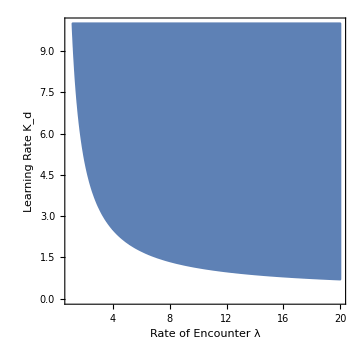

```mathematica
ntwrp1= Show[RegionPlot[TwoWins[λ,di,d1,kd,kf,α1,α2]==True,{λ,1,20},{kd,0,10}, ColorFunction->Blue],Axes->False,
Frame->{{True,True},{True,True}},
FrameStyle->Directive[Thick,Black,14],
FrameLabel->{Text[Style["Rate of Encounter λ",Black,20]],Text[Style["Learning Rate K_d",Black,20]]},
ImageSize->Medium]
```

```mathematica
.;,l
```

#### Δ = .1

```mathematica
λ=10;
di=0.15;
d1=0.25;
kd=7;
kf=3;
α1=1;
α2=0;
TwoWins[λ,di,d1,kd,kf,α1,α2]
```

True

```mathematica
Dynamic[{λ,kd}]
```

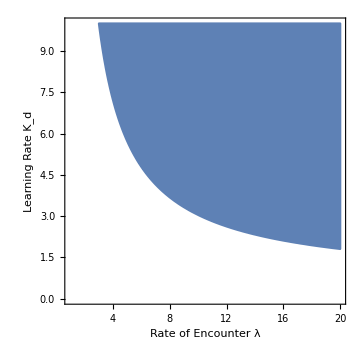

```mathematica
ntwrp2= Show[RegionPlot[TwoWins[λ,di,d1,kd,kf,α1,α2]==True,{λ,1,20},{kd,0,10}, ColorFunction->Blue],Axes->False,
Frame->{{True,True},{True,True}},
FrameStyle->Directive[Thick,Black,14],
FrameLabel->{Text[Style["Rate of Encounter λ",Black,20]],Text[Style["Learning Rate K_d",Black,20]]},
ImageSize->Medium]
```

#### Δ = .15

```mathematica
λ=10;
di=0.1;
d1=0.25;
kd=7;
kf=3;
α1=1;
α2=0;
TwoWins[λ,di,d1,kd,kf,α1,α2]
```

False

```mathematica
Dynamic[{λ,kd}]
```

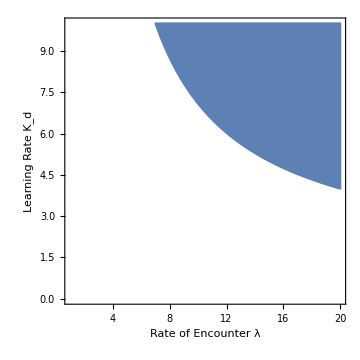

```mathematica
ntwrp3= Show[RegionPlot[TwoWins[λ,di,d1,kd,kf,α1,α2]==True,{λ,1,20},{kd,0,10}, ColorFunction->Blue],Axes->False,
Frame->{{True,True},{True,True}},
FrameStyle->Directive[Thick,Black,14],
FrameLabel->{Text[Style["Rate of Encounter λ",Black,20]],Text[Style["Learning Rate K_d",Black,20]]},
ImageSize->Medium]
```

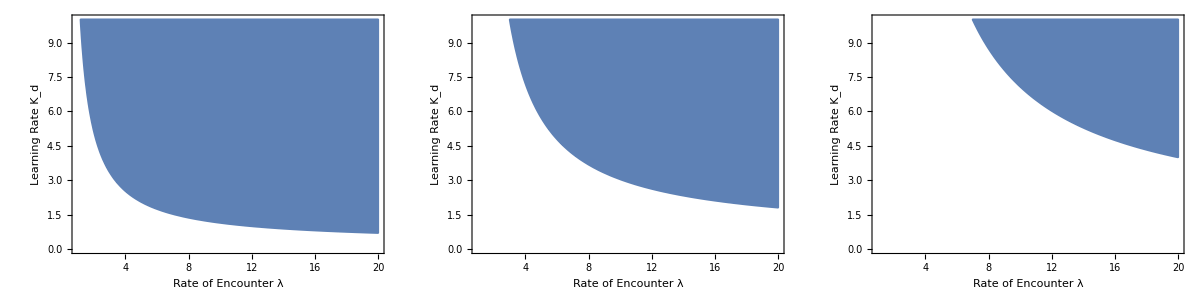

```mathematica
Grid[{{ntwrp1,ntwrp2,ntwrp3}}]
```

```mathematica
1. λ, kd - di = .15
```

### Row 2

#### Δ = .05

```mathematica
λ=10;
di=0.3;
d1=0.35;
kd=7;
kf=3;
α1=1;
α2=0;
TwoWins[λ,di,d1,kd,kf,α1,α2]
```

True

```mathematica
Dynamic[{λ,kd}]
```

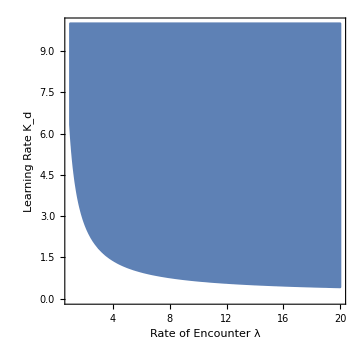

```mathematica
ntwrp4= Show[RegionPlot[TwoWins[λ,di,d1,kd,kf,α1,α2]==True,{λ,1,20},{kd,0,10}, ColorFunction->Blue],Axes->False,
Frame->{{True,True},{True,True}},
FrameStyle->Directive[Thick,Black,14],
FrameLabel->{Text[Style["Rate of Encounter λ",Black,20]],Text[Style["Learning Rate K_d",Black,20]]},
ImageSize->Medium]
```

#### Δ = .1

```mathematica
λ=10;
di=0.25;
d1=0.35;
kd=7;
kf=3;
α1=1;
α2=0;
TwoWins[λ,di,d1,kd,kf,α1,α2]
```

True

```mathematica
Dynamic[{λ,kd}]
```

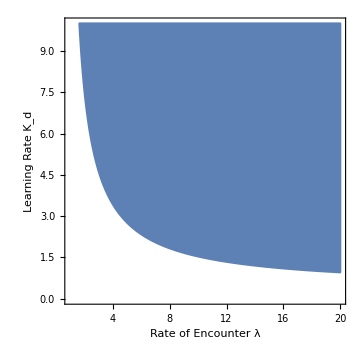

```mathematica
ntwrp5= Show[RegionPlot[TwoWins[λ,di,d1,kd,kf,α1,α2]==True,{λ,1,20},{kd,0,10}, ColorFunction->Blue],Axes->False,
Frame->{{True,True},{True,True}},
FrameStyle->Directive[Thick,Black,14],
FrameLabel->{Text[Style["Rate of Encounter λ",Black,20]],Text[Style["Learning Rate K_d",Black,20]]},
ImageSize->Medium]
```

#### Δ = .15

```mathematica
λ=10;
di=0.2;
d1=0.35;
kd=7;
kf=3;
α1=1;
α2=0;
TwoWins[λ,di,d1,kd,kf,α1,α2]
```

True

```mathematica
Dynamic[{λ,kd}]
```

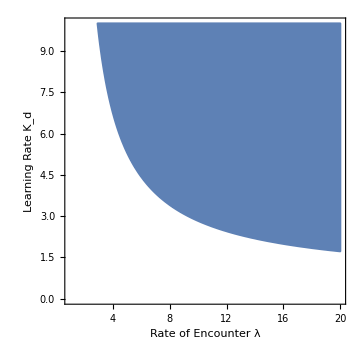

```mathematica
ntwrp6= Show[RegionPlot[TwoWins[λ,di,d1,kd,kf,α1,α2]==True,{λ,1,20},{kd,0,10}, ColorFunction->Blue],Axes->False,
Frame->{{True,True},{True,True}},
FrameStyle->Directive[Thick,Black,14],
FrameLabel->{Text[Style["Rate of Encounter λ",Black,20]],Text[Style["Learning Rate K_d",Black,20]]},
ImageSize->Medium]
```

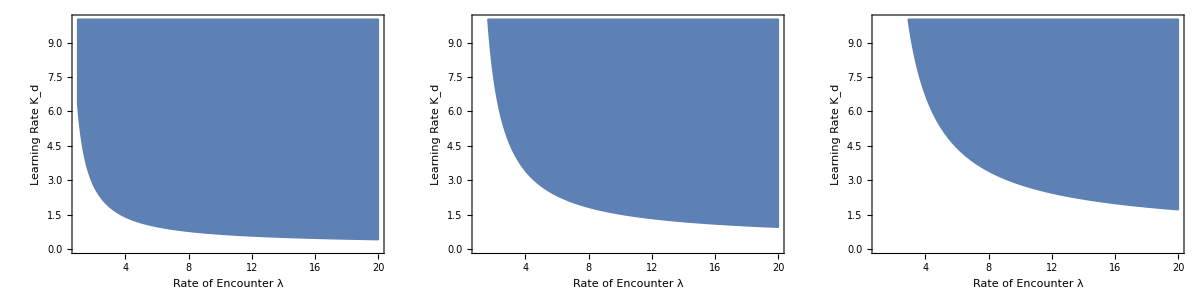

```mathematica
Grid[{{ntwrp4,ntwrp5,ntwrp6}}]
```

```mathematica
Total Grid
```

Grid Total

```mathematica
twrpgrid=Grid[{{Null,Text[Style["TraditionalForm`Δ\ 0.05",26,TextAlignment->Center]],Text[Style["TraditionalForm`Δ\ 0.1",26,TextAlignment->Center]],Text[Style["TraditionalForm`Δ\ 0.15",26,TextAlignment->Center]]},
{Rotate[Text[Style["d0 = .25",26,TextAlignment->Center]],90 Degree],ntwrp1,ntwrp2,ntwrp3},
{Rotate[Text[Style["d0 = .35",26,TextAlignment->Center]],90Degree],ntwrp4,ntwrp5,ntwrp6}}]
```

| TraditionalForm`Δ\ 0.05 | TraditionalForm`Δ\ 0.1 | TraditionalForm`Δ\ 0.15
d0 = .25 | -Graphics- | -Graphics- | -Graphics-
d0 = .35 | -Graphics- | -Graphics- | -Graphics-

### Grid

```mathematica
twrpgrid1=Grid[{{Null,Text[Style["TraditionalForm`Δ\ 0.05",26,TextAlignment->Center]],Text[Style["TraditionalForm`Δ\ 0.1",26,TextAlignment->Center]],Text[Style["TraditionalForm`Δ\ 0.15",26,TextAlignment->Center]]},
{Rotate[Text[Style["d0 = .25",26,TextAlignment->Center]],90 Degree],ntwrp1,ntwrp2,ntwrp3},
{Rotate[Text[Style["d0 = .35",26,TextAlignment->Center]],90Degree],ntwrp4,ntwrp5,ntwrp6}}]
```

| TraditionalForm`Δ\ 0.05 | TraditionalForm`Δ\ 0.1 | TraditionalForm`Δ\ 0.15
d0 = .25 | -Graphics- | -Graphics- | -Graphics-
d0 = .35 | -Graphics- | -Graphics- | -Graphics-

## Functions for Figs 3 and 4

```mathematica
(*These functions produce the data points below that are used to generate Figures 3,4,S3 and S4*)
```

```mathematica
Survival1[λ_?NumericQ,di_?NumericQ,d1_?NumericQ,kd_?NumericQ,kf_?NumericQ,α1_?NumericQ,cL_?NumericQ,cF_?NumericQ]:=Module[

{P,Q1,dl1,D1,F1,δ1,cap,cLfxn1,cFfxn1,sumfm1,fmag1},

(* step 1 set probability distribution *)
P[bigN_] := P[bigN]=((λ^bigN)Exp[-λ])/bigN!;
Q1[bigN_]:= Q1[bigN]=P[bigN]*Product[(α1(1-di)+(1-α1)(1-dl1[n])), {n,1,bigN}];
cap = Ceiling[Values[FindRoot[P[bigN]== 10^-10, {bigN,2λ}]][[1]]];

(* step 2: define danger and fear *)
dl1[n_]:=dl1[n]= d1*Exp[-kd*F1[n-1]];
D1[bigN_]:= D1[bigN]=Sum[(1-(α1(1-di) + (1-α1)(1-dl1[n]))),{n,1,bigN}] ;
F1[n_]:= F1[n]=D1[n]/ (kf + D1[n]);

(* calculate selection *)
Do[(* store final fear values as function of bigN - don't incorporate probability of experiencing bigN encounters yet *)
fmag1[bigN]=Values[NSolve[ 1-(α1(1-di)+(1-α1) (1-dl1[bigN]))==d1*Exp[-kd f],f]][[1]],
{bigN,0,cap}];
sumfm1= Sum[Q1[bigN],{bigN,0,cap}];(* sum over Q1 to use for turning into prob. dist. *)
cLfxn1 = (cL)(1 - α1);
cFfxn1=Sum[(Q1[bigN]/sumfm1)(fmag1[bigN]/((1/cF) +fmag1[bigN])),{bigN,0,cap}];(* cost experienced for any amount of fear; weighted by likelihood *)
δ1=Sum[P[bigN]-Q1[bigN], {bigN,0,cap}];

Clear[P,Q1,dl1,D1,F1];
((1-δ1)(1-cLfxn1) (1-cFfxn1))[[1]]
]
(*calculate the proportion of innate fear encoded by allele A1 as α1 that maximizes survival*)
α1max[λ_?NumericQ,di_?NumericQ,d1_?NumericQ,kd_?NumericQ,kf_?NumericQ,cL_?NumericQ,cF_?NumericQ]:=NArgMax[{Evaluate[Survival1[λ,di,d1,kd,kf,A1,cL,cF]],0≤A1≤1},A1]

(*sample parameters*)
λ=8;
di=0.25;
d1=0.3;
kd=5;
kf=5;
α1=.7;
α2=0.2;
cL=0.4;
cF=0.4;
(*sample data*)
sampledata= Interpolation[Table[α1max[λ,di,d1,kd,kf,cL,cF],{λ,0,10,.1},{kd,0,10,.1}],{{0,10},{0,10}}]
```

## Figure 3

### Data Points

```mathematica
(*data ran on cluster to expedite run time. Functions are copied below the data points for replication purposes*)
```

#### Δ = .02; Row 1

```mathematica
data = {{{0.1,0.1,1.},{0.1,0.2,1.},{0.1,0.30000000000000004,1.},{0.1,0.4,1.},{0.1,0.5,1.},{0.1,0.6,1.},{0.1,0.7000000000000001,1.},{0.1,0.8,1.},{0.1,0.9,1.},{0.1,1.,1.},{0.1,1.1,1.},{0.1,1.2000000000000002,1.},{0.1,1.3000000000000003,1.},{0.1,1.4000000000000001,1.},{0.1,1.5000000000000002,1.},{0.1,1.6,1.},{0.1,1.7000000000000002,1.},{0.1,1.8000000000000003,1.},{0.1,1.9000000000000001,1.},{0.1,2.,1.},{0.1,2.1,1.},{0.1,2.2,1.},{0.1,2.3000000000000003,1.},{0.1,2.4000000000000004,1.},{0.1,2.5000000000000004,1.},{0.1,2.6,1.},{0.1,2.7,1.},{0.1,2.8000000000000003,1.},{0.1,2.9000000000000004,1.},{0.1,3.0000000000000004,1.},{0.1,3.1,1.},{0.1,3.2,1.},{0.1,3.3000000000000003,1.},{0.1,3.4000000000000004,1.},{0.1,3.5000000000000004,1.},{0.1,3.6,1.},{0.1,3.7,1.},{0.1,3.8000000000000003,1.},{0.1,3.9000000000000004,1.},{0.1,4.,1.},{0.1,4.1,1.},{0.1,4.2,1.},{0.1,4.3,1.},{0.1,4.3999999999999995,1.},{0.1,4.5,1.},{0.1,4.6,1.},{0.1,4.7,1.},{0.1,4.8,1.},{0.1,4.9,1.},{0.1,5.,1.},{0.1,5.1,1.},{0.1,5.2,1.},{0.1,5.3,1.},{0.1,5.4,1.},{0.1,5.5,1.},{0.1,5.6,1.},{0.1,5.7,1.},{0.1,5.8,1.},{0.1,5.9,1.},{0.1,6.,1.},{0.1,6.1,1.},{0.1,6.2,1.},{0.1,6.3,1.},{0.1,6.4,1.},{0.1,6.5,1.},{0.1,6.6,1.},{0.1,6.7,1.},{0.1,6.8,1.},{0.1,6.9,1.},{0.1,7.,1.},{0.1,7.1,1.},{0.1,7.2,1.},{0.1,7.3,1.},{0.1,7.4,1.},{0.1,7.5,1.},{0.1,7.6,1.},{0.1,7.7,1.},{0.1,7.8,1.},{0.1,7.9,1.},{0.1,8.,1.},{0.1,8.1,1.},{0.1,8.2,1.},{0.1,8.3,1.},{0.1,8.4,1.},{0.1,8.5,1.},{0.1,8.6,1.},{0.1,8.7,1.},{0.1,8.8,1.},{0.1,8.9,1.},{0.1,9.,1.},{0.1,9.1,1.},{0.1,9.2,1.},{0.1,9.3,1.},{0.1,9.4,1.},{0.1,9.5,1.},{0.1,9.6,1.},{0.1,9.700000000000001,1.},{0.1,9.8,1.},{0.1,9.9,1.},{0.1,10.,1.}},{{0.2,0.1,1.},{0.2,0.2,1.},{0.2,0.30000000000000004,1.},{0.2,0.4,1.},{0.2,0.5,1.},{0.2,0.6,1.},{0.2,0.7000000000000001,1.},{0.2,0.8,1.},{0.2,0.9,1.},{0.2,1.,1.},{0.2,1.1,1.},{0.2,1.2000000000000002,1.},{0.2,1.3000000000000003,1.},{0.2,1.4000000000000001,1.},{0.2,1.5000000000000002,1.},{0.2,1.6,1.},{0.2,1.7000000000000002,1.},{0.2,1.8000000000000003,1.},{0.2,1.9000000000000001,1.},{0.2,2.,1.},{0.2,2.1,1.},{0.2,2.2,1.},{0.2,2.3000000000000003,1.},{0.2,2.4000000000000004,1.},{0.2,2.5000000000000004,1.},{0.2,2.6,1.},{0.2,2.7,1.},{0.2,2.8000000000000003,1.},{0.2,2.9000000000000004,1.},{0.2,3.0000000000000004,1.},{0.2,3.1,1.},{0.2,3.2,1.},{0.2,3.3000000000000003,1.},{0.2,3.4000000000000004,1.},{0.2,3.5000000000000004,1.},{0.2,3.6,1.},{0.2,3.7,1.},{0.2,3.8000000000000003,1.},{0.2,3.9000000000000004,1.},{0.2,4.,1.},{0.2,4.1,1.},{0.2,4.2,1.},{0.2,4.3,1.},{0.2,4.3999999999999995,1.},{0.2,4.5,1.},{0.2,4.6,1.},{0.2,4.7,1.},{0.2,4.8,1.},{0.2,4.9,1.},{0.2,5.,1.},{0.2,5.1,1.},{0.2,5.2,1.},{0.2,5.3,1.},{0.2,5.4,1.},{0.2,5.5,1.},{0.2,5.6,1.},{0.2,5.7,1.},{0.2,5.8,1.},{0.2,5.9,1.},{0.2,6.,1.},{0.2,6.1,1.},{0.2,6.2,1.},{0.2,6.3,1.},{0.2,6.4,1.},{0.2,6.5,1.},{0.2,6.6,1.},{0.2,6.7,1.},{0.2,6.8,1.},{0.2,6.9,1.},{0.2,7.,1.},{0.2,7.1,1.},{0.2,7.2,1.},{0.2,7.3,1.},{0.2,7.4,1.},{0.2,7.5,1.},{0.2,7.6,1.},{0.2,7.7,1.},{0.2,7.8,1.},{0.2,7.9,1.},{0.2,8.,1.},{0.2,8.1,1.},{0.2,8.2,1.},{0.2,8.3,1.},{0.2,8.4,1.},{0.2,8.5,1.},{0.2,8.6,1.},{0.2,8.7,1.},{0.2,8.8,1.},{0.2,8.9,1.},{0.2,9.,1.},{0.2,9.1,1.},{0.2,9.2,1.},{0.2,9.3,1.},{0.2,9.4,1.},{0.2,9.5,1.},{0.2,9.6,1.},{0.2,9.700000000000001,1.},{0.2,9.8,1.},{0.2,9.9,1.},{0.2,10.,1.}},{{0.30000000000000004,0.1,1.},{0.30000000000000004,0.2,1.},{0.30000000000000004,0.30000000000000004,1.},{0.30000000000000004,0.4,1.},{0.30000000000000004,0.5,1.},{0.30000000000000004,0.6,1.},{0.30000000000000004,0.7000000000000001,1.},{0.30000000000000004,0.8,1.},{0.30000000000000004,0.9,1.},{0.30000000000000004,1.,1.},{0.30000000000000004,1.1,1.},{0.30000000000000004,1.2000000000000002,1.},{0.30000000000000004,1.3000000000000003,1.},{0.30000000000000004,1.4000000000000001,1.},{0.30000000000000004,1.5000000000000002,1.},{0.30000000000000004,1.6,1.},{0.30000000000000004,1.7000000000000002,1.},{0.30000000000000004,1.8000000000000003,1.},{0.30000000000000004,1.9000000000000001,1.},{0.30000000000000004,2.,1.},{0.30000000000000004,2.1,1.},{0.30000000000000004,2.2,1.},{0.30000000000000004,2.3000000000000003,1.},{0.30000000000000004,2.4000000000000004,1.},{0.30000000000000004,2.5000000000000004,1.},{0.30000000000000004,2.6,1.},{0.30000000000000004,2.7,1.},{0.30000000000000004,2.8000000000000003,1.},{0.30000000000000004,2.9000000000000004,1.},{0.30000000000000004,3.0000000000000004,1.},{0.30000000000000004,3.1,1.},{0.30000000000000004,3.2,1.},{0.30000000000000004,3.3000000000000003,1.},{0.30000000000000004,3.4000000000000004,1.},{0.30000000000000004,3.5000000000000004,1.},{0.30000000000000004,3.6,1.},{0.30000000000000004,3.7,1.},{0.30000000000000004,3.8000000000000003,1.},{0.30000000000000004,3.9000000000000004,1.},{0.30000000000000004,4.,1.},{0.30000000000000004,4.1,1.},{0.30000000000000004,4.2,1.},{0.30000000000000004,4.3,1.},{0.30000000000000004,4.3999999999999995,1.},{0.30000000000000004,4.5,1.},{0.30000000000000004,4.6,1.},{0.30000000000000004,4.7,1.},{0.30000000000000004,4.8,1.},{0.30000000000000004,4.9,1.},{0.30000000000000004,5.,1.},{0.30000000000000004,5.1,1.},{0.30000000000000004,5.2,1.},{0.30000000000000004,5.3,1.},{0.30000000000000004,5.4,1.},{0.30000000000000004,5.5,1.},{0.30000000000000004,5.6,1.},{0.30000000000000004,5.7,1.},{0.30000000000000004,5.8,1.},{0.30000000000000004,5.9,1.},{0.30000000000000004,6.,1.},{0.30000000000000004,6.1,1.},{0.30000000000000004,6.2,1.},{0.30000000000000004,6.3,1.},{0.30000000000000004,6.4,1.},{0.30000000000000004,6.5,1.},{0.30000000000000004,6.6,1.},{0.30000000000000004,6.7,1.},{0.30000000000000004,6.8,1.},{0.30000000000000004,6.9,1.},{0.30000000000000004,7.,1.},{0.30000000000000004,7.1,1.},{0.30000000000000004,7.2,1.},{0.30000000000000004,7.3,1.},{0.30000000000000004,7.4,1.},{0.30000000000000004,7.5,1.},{0.30000000000000004,7.6,1.},{0.30000000000000004,7.7,1.},{0.30000000000000004,7.8,1.},{0.30000000000000004,7.9,1.},{0.30000000000000004,8.,1.},{0.30000000000000004,8.1,1.},{0.30000000000000004,8.2,1.},{0.30000000000000004,8.3,1.},{0.30000000000000004,8.4,1.},{0.30000000000000004,8.5,1.},{0.30000000000000004,8.6,1.},{0.30000000000000004,8.7,1.},{0.30000000000000004,8.8,1.},{0.30000000000000004,8.9,1.},{0.30000000000000004,9.,1.},{0.30000000000000004,9.1,1.},{0.30000000000000004,9.2,1.},{0.30000000000000004,9.3,1.},{0.30000000000000004,9.4,1.},{0.30000000000000004,9.5,1.},{0.30000000000000004,9.6,1.},{0.30000000000000004,9.700000000000001,1.},{0.30000000000000004,9.8,1.},{0.30000000000000004,9.9,1.},{0.30000000000000004,10.,1.}},{{0.4,0.1,1.},{0.4,0.2,1.},{0.4,0.30000000000000004,1.},{0.4,0.4,1.},{0.4,0.5,1.},{0.4,0.6,1.},{0.4,0.7000000000000001,1.},{0.4,0.8,1.},{0.4,0.9,1.},{0.4,1.,1.},{0.4,1.1,1.},{0.4,1.2000000000000002,1.},{0.4,1.3000000000000003,1.},{0.4,1.4000000000000001,1.},{0.4,1.5000000000000002,1.},{0.4,1.6,1.},{0.4,1.7000000000000002,1.},{0.4,1.8000000000000003,1.},{0.4,1.9000000000000001,1.},{0.4,2.,1.},{0.4,2.1,1.},{0.4,2.2,1.},{0.4,2.3000000000000003,1.},{0.4,2.4000000000000004,1.},{0.4,2.5000000000000004,1.},{0.4,2.6,1.},{0.4,2.7,1.},{0.4,2.8000000000000003,1.},{0.4,2.9000000000000004,1.},{0.4,3.0000000000000004,1.},{0.4,3.1,1.},{0.4,3.2,1.},{0.4,3.3000000000000003,1.},{0.4,3.4000000000000004,1.},{0.4,3.5000000000000004,1.},{0.4,3.6,1.},{0.4,3.7,1.},{0.4,3.8000000000000003,1.},{0.4,3.9000000000000004,1.},{0.4,4.,1.},{0.4,4.1,1.},{0.4,4.2,1.},{0.4,4.3,1.},{0.4,4.3999999999999995,1.},{0.4,4.5,1.},{0.4,4.6,1.},{0.4,4.7,1.},{0.4,4.8,1.},{0.4,4.9,1.},{0.4,5.,1.},{0.4,5.1,1.},{0.4,5.2,1.},{0.4,5.3,1.},{0.4,5.4,1.},{0.4,5.5,1.},{0.4,5.6,1.},{0.4,5.7,1.},{0.4,5.8,1.},{0.4,5.9,1.},{0.4,6.,1.},{0.4,6.1,1.},{0.4,6.2,1.},{0.4,6.3,1.},{0.4,6.4,1.},{0.4,6.5,1.},{0.4,6.6,1.},{0.4,6.7,1.},{0.4,6.8,1.},{0.4,6.9,1.},{0.4,7.,1.},{0.4,7.1,1.},{0.4,7.2,1.},{0.4,7.3,1.},{0.4,7.4,1.},{0.4,7.5,1.},{0.4,7.6,1.},{0.4,7.7,1.},{0.4,7.8,1.},{0.4,7.9,1.},{0.4,8.,1.},{0.4,8.1,1.},{0.4,8.2,1.},{0.4,8.3,1.},{0.4,8.4,1.},{0.4,8.5,1.},{0.4,8.6,1.},{0.4,8.7,1.},{0.4,8.8,1.},{0.4,8.9,1.},{0.4,9.,1.},{0.4,9.1,1.},{0.4,9.2,1.},{0.4,9.3,1.},{0.4,9.4,1.},{0.4,9.5,1.},{0.4,9.6,1.},{0.4,9.700000000000001,1.},{0.4,9.8,1.},{0.4,9.9,1.},{0.4,10.,1.}},{{0.5,0.1,1.},{0.5,0.2,1.},{0.5,0.30000000000000004,1.},{0.5,0.4,1.},{0.5,0.5,1.},{0.5,0.6,1.},{0.5,0.7000000000000001,1.},{0.5,0.8,1.},{0.5,0.9,1.},{0.5,1.,1.},{0.5,1.1,1.},{0.5,1.2000000000000002,1.},{0.5,1.3000000000000003,1.},{0.5,1.4000000000000001,1.},{0.5,1.5000000000000002,1.},{0.5,1.6,1.},{0.5,1.7000000000000002,1.},{0.5,1.8000000000000003,1.},{0.5,1.9000000000000001,1.},{0.5,2.,1.},{0.5,2.1,1.},{0.5,2.2,1.},{0.5,2.3000000000000003,1.},{0.5,2.4000000000000004,1.},{0.5,2.5000000000000004,1.},{0.5,2.6,1.},{0.5,2.7,1.},{0.5,2.8000000000000003,1.},{0.5,2.9000000000000004,1.},{0.5,3.0000000000000004,1.},{0.5,3.1,1.},{0.5,3.2,1.},{0.5,3.3000000000000003,1.},{0.5,3.4000000000000004,1.},{0.5,3.5000000000000004,1.},{0.5,3.6,1.},{0.5,3.7,1.},{0.5,3.8000000000000003,1.},{0.5,3.9000000000000004,1.},{0.5,4.,1.},{0.5,4.1,1.},{0.5,4.2,1.},{0.5,4.3,1.},{0.5,4.3999999999999995,1.},{0.5,4.5,1.},{0.5,4.6,1.},{0.5,4.7,1.},{0.5,4.8,1.},{0.5,4.9,1.},{0.5,5.,1.},{0.5,5.1,1.},{0.5,5.2,1.},{0.5,5.3,1.},{0.5,5.4,1.},{0.5,5.5,1.},{0.5,5.6,1.},{0.5,5.7,1.},{0.5,5.8,1.},{0.5,5.9,1.},{0.5,6.,1.},{0.5,6.1,1.},{0.5,6.2,1.},{0.5,6.3,1.},{0.5,6.4,1.},{0.5,6.5,1.},{0.5,6.6,1.},{0.5,6.7,1.},{0.5,6.8,1.},{0.5,6.9,1.},{0.5,7.,1.},{0.5,7.1,1.},{0.5,7.2,1.},{0.5,7.3,1.},{0.5,7.4,1.},{0.5,7.5,1.},{0.5,7.6,1.},{0.5,7.7,1.},{0.5,7.8,1.},{0.5,7.9,1.},{0.5,8.,1.},{0.5,8.1,1.},{0.5,8.2,1.},{0.5,8.3,1.},{0.5,8.4,1.},{0.5,8.5,1.},{0.5,8.6,1.},{0.5,8.7,1.},{0.5,8.8,1.},{0.5,8.9,1.},{0.5,9.,1.},{0.5,9.1,1.},{0.5,9.2,1.},{0.5,9.3,1.},{0.5,9.4,1.},{0.5,9.5,1.},{0.5,9.6,1.},{0.5,9.700000000000001,1.},{0.5,9.8,1.},{0.5,9.9,1.},{0.5,10.,1.}},{{0.6000000000000001,0.1,1.},{0.6000000000000001,0.2,1.},{0.6000000000000001,0.30000000000000004,1.},{0.6000000000000001,0.4,1.},{0.6000000000000001,0.5,1.},{0.6000000000000001,0.6,1.},{0.6000000000000001,0.7000000000000001,1.},{0.6000000000000001,0.8,1.},{0.6000000000000001,0.9,1.},{0.6000000000000001,1.,1.},{0.6000000000000001,1.1,1.},{0.6000000000000001,1.2000000000000002,1.},{0.6000000000000001,1.3000000000000003,1.},{0.6000000000000001,1.4000000000000001,1.},{0.6000000000000001,1.5000000000000002,1.},{0.6000000000000001,1.6,1.},{0.6000000000000001,1.7000000000000002,1.},{0.6000000000000001,1.8000000000000003,1.},{0.6000000000000001,1.9000000000000001,1.},{0.6000000000000001,2.,1.},{0.6000000000000001,2.1,1.},{0.6000000000000001,2.2,1.},{0.6000000000000001,2.3000000000000003,1.},{0.6000000000000001,2.4000000000000004,1.},{0.6000000000000001,2.5000000000000004,1.},{0.6000000000000001,2.6,1.},{0.6000000000000001,2.7,1.},{0.6000000000000001,2.8000000000000003,1.},{0.6000000000000001,2.9000000000000004,1.},{0.6000000000000001,3.0000000000000004,1.},{0.6000000000000001,3.1,1.},{0.6000000000000001,3.2,1.},{0.6000000000000001,3.3000000000000003,1.},{0.6000000000000001,3.4000000000000004,1.},{0.6000000000000001,3.5000000000000004,1.},{0.6000000000000001,3.6,1.},{0.6000000000000001,3.7,1.},{0.6000000000000001,3.8000000000000003,1.},{0.6000000000000001,3.9000000000000004,1.},{0.6000000000000001,4.,1.},{0.6000000000000001,4.1,1.},{0.6000000000000001,4.2,1.},{0.6000000000000001,4.3,1.},{0.6000000000000001,4.3999999999999995,1.},{0.6000000000000001,4.5,1.},{0.6000000000000001,4.6,1.},{0.6000000000000001,4.7,1.},{0.6000000000000001,4.8,1.},{0.6000000000000001,4.9,1.},{0.6000000000000001,5.,1.},{0.6000000000000001,5.1,1.},{0.6000000000000001,5.2,1.},{0.6000000000000001,5.3,1.},{0.6000000000000001,5.4,1.},{0.6000000000000001,5.5,1.},{0.6000000000000001,5.6,1.},{0.6000000000000001,5.7,1.},{0.6000000000000001,5.8,1.},{0.6000000000000001,5.9,1.},{0.6000000000000001,6.,1.},{0.6000000000000001,6.1,1.},{0.6000000000000001,6.2,1.},{0.6000000000000001,6.3,1.},{0.6000000000000001,6.4,1.},{0.6000000000000001,6.5,1.},{0.6000000000000001,6.6,1.},{0.6000000000000001,6.7,1.},{0.6000000000000001,6.8,1.},{0.6000000000000001,6.9,1.},{0.6000000000000001,7.,1.},{0.6000000000000001,7.1,1.},{0.6000000000000001,7.2,1.},{0.6000000000000001,7.3,1.},{0.6000000000000001,7.4,1.},{0.6000000000000001,7.5,1.},{0.6000000000000001,7.6,1.},{0.6000000000000001,7.7,1.},{0.6000000000000001,7.8,1.},{0.6000000000000001,7.9,1.},{0.6000000000000001,8.,1.},{0.6000000000000001,8.1,1.},{0.6000000000000001,8.2,1.},{0.6000000000000001,8.3,1.},{0.6000000000000001,8.4,1.},{0.6000000000000001,8.5,1.},{0.6000000000000001,8.6,1.},{0.6000000000000001,8.7,1.},{0.6000000000000001,8.8,1.},{0.6000000000000001,8.9,1.},{0.6000000000000001,9.,1.},{0.6000000000000001,9.1,1.},{0.6000000000000001,9.2,1.},{0.6000000000000001,9.3,1.},{0.6000000000000001,9.4,1.},{0.6000000000000001,9.5,1.},{0.6000000000000001,9.6,1.},{0.6000000000000001,9.700000000000001,1.},{0.6000000000000001,9.8,1.},{0.6000000000000001,9.9,1.},{0.6000000000000001,10.,1.}},{{0.7000000000000001,0.1,1.},{0.7000000000000001,0.2,1.},{0.7000000000000001,0.30000000000000004,1.},{0.7000000000000001,0.4,1.},{0.7000000000000001,0.5,1.},{0.7000000000000001,0.6,1.},{0.7000000000000001,0.7000000000000001,1.},{0.7000000000000001,0.8,1.},{0.7000000000000001,0.9,1.},{0.7000000000000001,1.,1.},{0.7000000000000001,1.1,1.},{0.7000000000000001,1.2000000000000002,1.},{0.7000000000000001,1.3000000000000003,1.},{0.7000000000000001,1.4000000000000001,1.},{0.7000000000000001,1.5000000000000002,1.},{0.7000000000000001,1.6,1.},{0.7000000000000001,1.7000000000000002,1.},{0.7000000000000001,1.8000000000000003,1.},{0.7000000000000001,1.9000000000000001,1.},{0.7000000000000001,2.,1.},{0.7000000000000001,2.1,1.},{0.7000000000000001,2.2,1.},{0.7000000000000001,2.3000000000000003,1.},{0.7000000000000001,2.4000000000000004,1.},{0.7000000000000001,2.5000000000000004,1.},{0.7000000000000001,2.6,1.},{0.7000000000000001,2.7,1.},{0.7000000000000001,2.8000000000000003,1.},{0.7000000000000001,2.9000000000000004,1.},{0.7000000000000001,3.0000000000000004,1.},{0.7000000000000001,3.1,1.},{0.7000000000000001,3.2,1.},{0.7000000000000001,3.3000000000000003,1.},{0.7000000000000001,3.4000000000000004,1.},{0.7000000000000001,3.5000000000000004,1.},{0.7000000000000001,3.6,1.},{0.7000000000000001,3.7,1.},{0.7000000000000001,3.8000000000000003,1.},{0.7000000000000001,3.9000000000000004,1.},{0.7000000000000001,4.,1.},{0.7000000000000001,4.1,1.},{0.7000000000000001,4.2,1.},{0.7000000000000001,4.3,1.},{0.7000000000000001,4.3999999999999995,1.},{0.7000000000000001,4.5,1.},{0.7000000000000001,4.6,1.},{0.7000000000000001,4.7,1.},{0.7000000000000001,4.8,1.},{0.7000000000000001,4.9,1.},{0.7000000000000001,5.,1.},{0.7000000000000001,5.1,1.},{0.7000000000000001,5.2,1.},{0.7000000000000001,5.3,1.},{0.7000000000000001,5.4,1.},{0.7000000000000001,5.5,1.},{0.7000000000000001,5.6,1.},{0.7000000000000001,5.7,1.},{0.7000000000000001,5.8,1.},{0.7000000000000001,5.9,1.},{0.7000000000000001,6.,1.},{0.7000000000000001,6.1,1.},{0.7000000000000001,6.2,1.},{0.7000000000000001,6.3,1.},{0.7000000000000001,6.4,1.},{0.7000000000000001,6.5,1.},{0.7000000000000001,6.6,1.},{0.7000000000000001,6.7,1.},{0.7000000000000001,6.8,1.},{0.7000000000000001,6.9,1.},{0.7000000000000001,7.,1.},{0.7000000000000001,7.1,1.},{0.7000000000000001,7.2,1.},{0.7000000000000001,7.3,1.},{0.7000000000000001,7.4,1.},{0.7000000000000001,7.5,1.},{0.7000000000000001,7.6,1.},{0.7000000000000001,7.7,1.},{0.7000000000000001,7.8,1.},{0.7000000000000001,7.9,1.},{0.7000000000000001,8.,1.},{0.7000000000000001,8.1,1.},{0.7000000000000001,8.2,1.},{0.7000000000000001,8.3,1.},{0.7000000000000001,8.4,1.},{0.7000000000000001,8.5,1.},{0.7000000000000001,8.6,1.},{0.7000000000000001,8.7,1.},{0.7000000000000001,8.8,1.},{0.7000000000000001,8.9,1.},{0.7000000000000001,9.,1.},{0.7000000000000001,9.1,1.},{0.7000000000000001,9.2,1.},{0.7000000000000001,9.3,1.},{0.7000000000000001,9.4,1.},{0.7000000000000001,9.5,1.},{0.7000000000000001,9.6,1.},{0.7000000000000001,9.700000000000001,1.},{0.7000000000000001,9.8,1.},{0.7000000000000001,9.9,1.},{0.7000000000000001,10.,1.}},{{0.8,0.1,1.},{0.8,0.2,1.},{0.8,0.30000000000000004,1.},{0.8,0.4,1.},{0.8,0.5,1.},{0.8,0.6,1.},{0.8,0.7000000000000001,1.},{0.8,0.8,1.},{0.8,0.9,1.},{0.8,1.,1.},{0.8,1.1,1.},{0.8,1.2000000000000002,1.},{0.8,1.3000000000000003,1.},{0.8,1.4000000000000001,1.},{0.8,1.5000000000000002,1.},{0.8,1.6,1.},{0.8,1.7000000000000002,1.},{0.8,1.8000000000000003,1.},{0.8,1.9000000000000001,1.},{0.8,2.,1.},{0.8,2.1,1.},{0.8,2.2,1.},{0.8,2.3000000000000003,1.},{0.8,2.4000000000000004,1.},{0.8,2.5000000000000004,1.},{0.8,2.6,1.},{0.8,2.7,1.},{0.8,2.8000000000000003,1.},{0.8,2.9000000000000004,1.},{0.8,3.0000000000000004,1.},{0.8,3.1,1.},{0.8,3.2,1.},{0.8,3.3000000000000003,1.},{0.8,3.4000000000000004,1.},{0.8,3.5000000000000004,1.},{0.8,3.6,1.},{0.8,3.7,1.},{0.8,3.8000000000000003,1.},{0.8,3.9000000000000004,1.},{0.8,4.,1.},{0.8,4.1,1.},{0.8,4.2,1.},{0.8,4.3,1.},{0.8,4.3999999999999995,1.},{0.8,4.5,1.},{0.8,4.6,1.},{0.8,4.7,1.},{0.8,4.8,1.},{0.8,4.9,1.},{0.8,5.,1.},{0.8,5.1,1.},{0.8,5.2,1.},{0.8,5.3,1.},{0.8,5.4,1.},{0.8,5.5,1.},{0.8,5.6,1.},{0.8,5.7,1.},{0.8,5.8,1.},{0.8,5.9,1.},{0.8,6.,1.},{0.8,6.1,1.},{0.8,6.2,1.},{0.8,6.3,1.},{0.8,6.4,1.},{0.8,6.5,1.},{0.8,6.6,1.},{0.8,6.7,1.},{0.8,6.8,1.},{0.8,6.9,1.},{0.8,7.,1.},{0.8,7.1,1.},{0.8,7.2,1.},{0.8,7.3,1.},{0.8,7.4,1.},{0.8,7.5,1.},{0.8,7.6,1.},{0.8,7.7,1.},{0.8,7.8,1.},{0.8,7.9,1.},{0.8,8.,1.},{0.8,8.1,1.},{0.8,8.2,1.},{0.8,8.3,1.},{0.8,8.4,1.},{0.8,8.5,1.},{0.8,8.6,1.},{0.8,8.7,1.},{0.8,8.8,1.},{0.8,8.9,1.},{0.8,9.,1.},{0.8,9.1,1.},{0.8,9.2,1.},{0.8,9.3,1.},{0.8,9.4,1.},{0.8,9.5,1.},{0.8,9.6,1.},{0.8,9.700000000000001,1.},{0.8,9.8,1.},{0.8,9.9,1.},{0.8,10.,1.}},{{0.9000000000000001,0.1,1.},{0.9000000000000001,0.2,1.},{0.9000000000000001,0.30000000000000004,1.},{0.9000000000000001,0.4,1.},{0.9000000000000001,0.5,1.},{0.9000000000000001,0.6,1.},{0.9000000000000001,0.7000000000000001,1.},{0.9000000000000001,0.8,1.},{0.9000000000000001,0.9,1.},{0.9000000000000001,1.,1.},{0.9000000000000001,1.1,1.},{0.9000000000000001,1.2000000000000002,1.},{0.9000000000000001,1.3000000000000003,1.},{0.9000000000000001,1.4000000000000001,1.},{0.9000000000000001,1.5000000000000002,1.},{0.9000000000000001,1.6,1.},{0.9000000000000001,1.7000000000000002,1.},{0.9000000000000001,1.8000000000000003,1.},{0.9000000000000001,1.9000000000000001,1.},{0.9000000000000001,2.,1.},{0.9000000000000001,2.1,1.},{0.9000000000000001,2.2,1.},{0.9000000000000001,2.3000000000000003,1.},{0.9000000000000001,2.4000000000000004,1.},{0.9000000000000001,2.5000000000000004,1.},{0.9000000000000001,2.6,1.},{0.9000000000000001,2.7,1.},{0.9000000000000001,2.8000000000000003,1.},{0.9000000000000001,2.9000000000000004,1.},{0.9000000000000001,3.0000000000000004,1.},{0.9000000000000001,3.1,1.},{0.9000000000000001,3.2,1.},{0.9000000000000001,3.3000000000000003,1.},{0.9000000000000001,3.4000000000000004,1.},{0.9000000000000001,3.5000000000000004,1.},{0.9000000000000001,3.6,1.},{0.9000000000000001,3.7,1.},{0.9000000000000001,3.8000000000000003,1.},{0.9000000000000001,3.9000000000000004,1.},{0.9000000000000001,4.,1.},{0.9000000000000001,4.1,1.},{0.9000000000000001,4.2,1.},{0.9000000000000001,4.3,1.},{0.9000000000000001,4.3999999999999995,1.},{0.9000000000000001,4.5,1.},{0.9000000000000001,4.6,1.},{0.9000000000000001,4.7,1.},{0.9000000000000001,4.8,1.},{0.9000000000000001,4.9,1.},{0.9000000000000001,5.,1.},{0.9000000000000001,5.1,1.},{0.9000000000000001,5.2,1.},{0.9000000000000001,5.3,1.},{0.9000000000000001,5.4,1.},{0.9000000000000001,5.5,1.},{0.9000000000000001,5.6,1.},{0.9000000000000001,5.7,1.},{0.9000000000000001,5.8,1.},{0.9000000000000001,5.9,1.},{0.9000000000000001,6.,1.},{0.9000000000000001,6.1,1.},{0.9000000000000001,6.2,1.},{0.9000000000000001,6.3,1.},{0.9000000000000001,6.4,1.},{0.9000000000000001,6.5,1.},{0.9000000000000001,6.6,1.},{0.9000000000000001,6.7,1.},{0.9000000000000001,6.8,1.},{0.9000000000000001,6.9,1.},{0.9000000000000001,7.,1.},{0.9000000000000001,7.1,1.},{0.9000000000000001,7.2,1.},{0.9000000000000001,7.3,1.},{0.9000000000000001,7.4,1.},{0.9000000000000001,7.5,1.},{0.9000000000000001,7.6,1.},{0.9000000000000001,7.7,1.},{0.9000000000000001,7.8,1.},{0.9000000000000001,7.9,1.},{0.9000000000000001,8.,1.},{0.9000000000000001,8.1,1.},{0.9000000000000001,8.2,1.},{0.9000000000000001,8.3,1.},{0.9000000000000001,8.4,1.},{0.9000000000000001,8.5,1.},{0.9000000000000001,8.6,1.},{0.9000000000000001,8.7,1.},{0.9000000000000001,8.8,1.},{0.9000000000000001,8.9,1.},{0.9000000000000001,9.,1.},{0.9000000000000001,9.1,1.},{0.9000000000000001,9.2,1.},{0.9000000000000001,9.3,1.},{0.9000000000000001,9.4,1.},{0.9000000000000001,9.5,1.},{0.9000000000000001,9.6,1.},{0.9000000000000001,9.700000000000001,1.},{0.9000000000000001,9.8,1.},{0.9000000000000001,9.9,1.},{0.9000000000000001,10.,1.}},{{1.,0.1,1.},{1.,0.2,1.},{1.,0.30000000000000004,1.},{1.,0.4,1.},{1.,0.5,1.},{1.,0.6,1.},{1.,0.7000000000000001,1.},{1.,0.8,1.},{1.,0.9,1.},{1.,1.,1.},{1.,1.1,1.},{1.,1.2000000000000002,1.},{1.,1.3000000000000003,1.},{1.,1.4000000000000001,1.},{1.,1.5000000000000002,1.},{1.,1.6,1.},{1.,1.7000000000000002,1.},{1.,1.8000000000000003,1.},{1.,1.9000000000000001,1.},{1.,2.,1.},{1.,2.1,1.},{1.,2.2,1.},{1.,2.3000000000000003,1.},{1.,2.4000000000000004,1.},{1.,2.5000000000000004,1.},{1.,2.6,1.},{1.,2.7,1.},{1.,2.8000000000000003,1.},{1.,2.9000000000000004,1.},{1.,3.0000000000000004,1.},{1.,3.1,1.},{1.,3.2,1.},{1.,3.3000000000000003,1.},{1.,3.4000000000000004,1.},{1.,3.5000000000000004,1.},{1.,3.6,1.},{1.,3.7,1.},{1.,3.8000000000000003,1.},{1.,3.9000000000000004,1.},{1.,4.,1.},{1.,4.1,1.},{1.,4.2,1.},{1.,4.3,1.},{1.,4.3999999999999995,1.},{1.,4.5,1.},{1.,4.6,1.},{1.,4.7,1.},{1.,4.8,1.},{1.,4.9,1.},{1.,5.,1.},{1.,5.1,1.},{1.,5.2,1.},{1.,5.3,1.},{1.,5.4,1.},{1.,5.5,1.},{1.,5.6,1.},{1.,5.7,1.},{1.,5.8,1.},{1.,5.9,1.},{1.,6.,1.},{1.,6.1,1.},{1.,6.2,1.},{1.,6.3,1.},{1.,6.4,1.},{1.,6.5,1.},{1.,6.6,1.},{1.,6.7,1.},{1.,6.8,1.},{1.,6.9,1.},{1.,7.,1.},{1.,7.1,1.},{1.,7.2,1.},{1.,7.3,1.},{1.,7.4,1.},{1.,7.5,1.},{1.,7.6,1.},{1.,7.7,1.},{1.,7.8,1.},{1.,7.9,1.},{1.,8.,1.},{1.,8.1,1.},{1.,8.2,1.},{1.,8.3,1.},{1.,8.4,1.},{1.,8.5,1.},{1.,8.6,1.},{1.,8.7,1.},{1.,8.8,1.},{1.,8.9,1.},{1.,9.,1.},{1.,9.1,1.},{1.,9.2,1.},{1.,9.3,1.},{1.,9.4,1.},{1.,9.5,1.},{1.,9.6,1.},{1.,9.700000000000001,1.},{1.,9.8,1.},{1.,9.9,1.},{1.,10.,1.}},{{1.1,0.1,1.},{1.1,0.2,1.},{1.1,0.30000000000000004,1.},{1.1,0.4,1.},{1.1,0.5,1.},{1.1,0.6,1.},{1.1,0.7000000000000001,1.},{1.1,0.8,1.},{1.1,0.9,1.},{1.1,1.,1.},{1.1,1.1,1.},{1.1,1.2000000000000002,1.},{1.1,1.3000000000000003,1.},{1.1,1.4000000000000001,1.},{1.1,1.5000000000000002,1.},{1.1,1.6,1.},{1.1,1.7000000000000002,1.},{1.1,1.8000000000000003,1.},{1.1,1.9000000000000001,1.},{1.1,2.,1.},{1.1,2.1,1.},{1.1,2.2,1.},{1.1,2.3000000000000003,1.},{1.1,2.4000000000000004,1.},{1.1,2.5000000000000004,1.},{1.1,2.6,1.},{1.1,2.7,1.},{1.1,2.8000000000000003,1.},{1.1,2.9000000000000004,1.},{1.1,3.0000000000000004,1.},{1.1,3.1,1.},{1.1,3.2,1.},{1.1,3.3000000000000003,1.},{1.1,3.4000000000000004,1.},{1.1,3.5000000000000004,1.},{1.1,3.6,1.},{1.1,3.7,1.},{1.1,3.8000000000000003,1.},{1.1,3.9000000000000004,1.},{1.1,4.,1.},{1.1,4.1,1.},{1.1,4.2,1.},{1.1,4.3,1.},{1.1,4.3999999999999995,1.},{1.1,4.5,1.},{1.1,4.6,1.},{1.1,4.7,1.},{1.1,4.8,1.},{1.1,4.9,1.},{1.1,5.,1.},{1.1,5.1,1.},{1.1,5.2,1.},{1.1,5.3,1.},{1.1,5.4,1.},{1.1,5.5,1.},{1.1,5.6,1.},{1.1,5.7,1.},{1.1,5.8,1.},{1.1,5.9,1.},{1.1,6.,1.},{1.1,6.1,1.},{1.1,6.2,1.},{1.1,6.3,1.},{1.1,6.4,1.},{1.1,6.5,1.},{1.1,6.6,1.},{1.1,6.7,1.},{1.1,6.8,1.},{1.1,6.9,1.},{1.1,7.,1.},{1.1,7.1,1.},{1.1,7.2,1.},{1.1,7.3,1.},{1.1,7.4,1.},{1.1,7.5,1.},{1.1,7.6,1.},{1.1,7.7,1.},{1.1,7.8,1.},{1.1,7.9,1.},{1.1,8.,1.},{1.1,8.1,1.},{1.1,8.2,1.},{1.1,8.3,1.},{1.1,8.4,1.},{1.1,8.5,1.},{1.1,8.6,1.},{1.1,8.7,1.},{1.1,8.8,1.},{1.1,8.9,1.},{1.1,9.,1.},{1.1,9.1,1.},{1.1,9.2,1.},{1.1,9.3,1.},{1.1,9.4,1.},{1.1,9.5,1.},{1.1,9.6,1.},{1.1,9.700000000000001,1.},{1.1,9.8,1.},{1.1,9.9,1.},{1.1,10.,1.}},{{1.2,0.1,1.},{1.2,0.2,1.},{1.2,0.30000000000000004,1.},{1.2,0.4,1.},{1.2,0.5,1.},{1.2,0.6,1.},{1.2,0.7000000000000001,1.},{1.2,0.8,1.},{1.2,0.9,1.},{1.2,1.,1.},{1.2,1.1,1.},{1.2,1.2000000000000002,1.},{1.2,1.3000000000000003,1.},{1.2,1.4000000000000001,1.},{1.2,1.5000000000000002,1.},{1.2,1.6,1.},{1.2,1.7000000000000002,1.},{1.2,1.8000000000000003,1.},{1.2,1.9000000000000001,1.},{1.2,2.,1.},{1.2,2.1,1.},{1.2,2.2,1.},{1.2,2.3000000000000003,1.},{1.2,2.4000000000000004,1.},{1.2,2.5000000000000004,1.},{1.2,2.6,1.},{1.2,2.7,1.},{1.2,2.8000000000000003,1.},{1.2,2.9000000000000004,1.},{1.2,3.0000000000000004,1.},{1.2,3.1,1.},{1.2,3.2,1.},{1.2,3.3000000000000003,1.},{1.2,3.4000000000000004,1.},{1.2,3.5000000000000004,1.},{1.2,3.6,1.},{1.2,3.7,1.},{1.2,3.8000000000000003,1.},{1.2,3.9000000000000004,1.},{1.2,4.,1.},{1.2,4.1,1.},{1.2,4.2,1.},{1.2,4.3,1.},{1.2,4.3999999999999995,1.},{1.2,4.5,1.},{1.2,4.6,1.},{1.2,4.7,1.},{1.2,4.8,1.},{1.2,4.9,1.},{1.2,5.,1.},{1.2,5.1,1.},{1.2,5.2,1.},{1.2,5.3,1.},{1.2,5.4,1.},{1.2,5.5,1.},{1.2,5.6,1.},{1.2,5.7,1.},{1.2,5.8,1.},{1.2,5.9,1.},{1.2,6.,1.},{1.2,6.1,1.},{1.2,6.2,1.},{1.2,6.3,1.},{1.2,6.4,1.},{1.2,6.5,1.},{1.2,6.6,1.},{1.2,6.7,1.},{1.2,6.8,1.},{1.2,6.9,1.},{1.2,7.,1.},{1.2,7.1,1.},{1.2,7.2,1.},{1.2,7.3,1.},{1.2,7.4,1.},{1.2,7.5,1.},{1.2,7.6,1.},{1.2,7.7,1.},{1.2,7.8,1.},{1.2,7.9,1.},{1.2,8.,1.},{1.2,8.1,1.},{1.2,8.2,1.},{1.2,8.3,1.},{1.2,8.4,1.},{1.2,8.5,1.},{1.2,8.6,1.},{1.2,8.7,1.},{1.2,8.8,1.},{1.2,8.9,1.},{1.2,9.,1.},{1.2,9.1,1.},{1.2,9.2,1.},{1.2,9.3,1.},{1.2,9.4,1.},{1.2,9.5,1.},{1.2,9.6,1.},{1.2,9.700000000000001,1.},{1.2,9.8,1.},{1.2,9.9,1.},{1.2,10.,1.}},{{1.3000000000000003,0.1,1.},{1.3000000000000003,0.2,1.},{1.3000000000000003,0.30000000000000004,1.},{1.3000000000000003,0.4,1.},{1.3000000000000003,0.5,1.},{1.3000000000000003,0.6,1.},{1.3000000000000003,0.7000000000000001,1.},{1.3000000000000003,0.8,1.},{1.3000000000000003,0.9,1.},{1.3000000000000003,1.,1.},{1.3000000000000003,1.1,1.},{1.3000000000000003,1.2000000000000002,1.},{1.3000000000000003,1.3000000000000003,1.},{1.3000000000000003,1.4000000000000001,1.},{1.3000000000000003,1.5000000000000002,1.},{1.3000000000000003,1.6,1.},{1.3000000000000003,1.7000000000000002,1.},{1.3000000000000003,1.8000000000000003,1.},{1.3000000000000003,1.9000000000000001,1.},{1.3000000000000003,2.,1.},{1.3000000000000003,2.1,1.},{1.3000000000000003,2.2,1.},{1.3000000000000003,2.3000000000000003,1.},{1.3000000000000003,2.4000000000000004,1.},{1.3000000000000003,2.5000000000000004,1.},{1.3000000000000003,2.6,1.},{1.3000000000000003,2.7,1.},{1.3000000000000003,2.8000000000000003,1.},{1.3000000000000003,2.9000000000000004,1.},{1.3000000000000003,3.0000000000000004,1.},{1.3000000000000003,3.1,1.},{1.3000000000000003,3.2,1.},{1.3000000000000003,3.3000000000000003,1.},{1.3000000000000003,3.4000000000000004,1.},{1.3000000000000003,3.5000000000000004,1.},{1.3000000000000003,3.6,1.},{1.3000000000000003,3.7,1.},{1.3000000000000003,3.8000000000000003,1.},{1.3000000000000003,3.9000000000000004,1.},{1.3000000000000003,4.,1.},{1.3000000000000003,4.1,1.},{1.3000000000000003,4.2,1.},{1.3000000000000003,4.3,1.},{1.3000000000000003,4.3999999999999995,1.},{1.3000000000000003,4.5,1.},{1.3000000000000003,4.6,1.},{1.3000000000000003,4.7,1.},{1.3000000000000003,4.8,1.},{1.3000000000000003,4.9,1.},{1.3000000000000003,5.,1.},{1.3000000000000003,5.1,1.},{1.3000000000000003,5.2,1.},{1.3000000000000003,5.3,1.},{1.3000000000000003,5.4,1.},{1.3000000000000003,5.5,1.},{1.3000000000000003,5.6,1.},{1.3000000000000003,5.7,1.},{1.3000000000000003,5.8,1.},{1.3000000000000003,5.9,1.},{1.3000000000000003,6.,1.},{1.3000000000000003,6.1,1.},{1.3000000000000003,6.2,1.},{1.3000000000000003,6.3,1.},{1.3000000000000003,6.4,1.},{1.3000000000000003,6.5,1.},{1.3000000000000003,6.6,1.},{1.3000000000000003,6.7,1.},{1.3000000000000003,6.8,1.},{1.3000000000000003,6.9,1.},{1.3000000000000003,7.,1.},{1.3000000000000003,7.1,1.},{1.3000000000000003,7.2,1.},{1.3000000000000003,7.3,1.},{1.3000000000000003,7.4,1.},{1.3000000000000003,7.5,1.},{1.3000000000000003,7.6,1.},{1.3000000000000003,7.7,1.},{1.3000000000000003,7.8,1.},{1.3000000000000003,7.9,1.},{1.3000000000000003,8.,1.},{1.3000000000000003,8.1,1.},{1.3000000000000003,8.2,1.},{1.3000000000000003,8.3,1.},{1.3000000000000003,8.4,1.},{1.3000000000000003,8.5,1.},{1.3000000000000003,8.6,1.},{1.3000000000000003,8.7,1.},{1.3000000000000003,8.8,1.},{1.3000000000000003,8.9,1.},{1.3000000000000003,9.,1.},{1.3000000000000003,9.1,1.},{1.3000000000000003,9.2,1.},{1.3000000000000003,9.3,1.},{1.3000000000000003,9.4,1.},{1.3000000000000003,9.5,1.},{1.3000000000000003,9.6,1.},{1.3000000000000003,9.700000000000001,1.},{1.3000000000000003,9.8,1.},{1.3000000000000003,9.9,1.},{1.3000000000000003,10.,1.}},{{1.4000000000000004,0.1,1.},{1.4000000000000004,0.2,1.},{1.4000000000000004,0.30000000000000004,1.},{1.4000000000000004,0.4,1.},{1.4000000000000004,0.5,1.},{1.4000000000000004,0.6,1.},{1.4000000000000004,0.7000000000000001,1.},{1.4000000000000004,0.8,1.},{1.4000000000000004,0.9,1.},{1.4000000000000004,1.,1.},{1.4000000000000004,1.1,1.},{1.4000000000000004,1.2000000000000002,1.},{1.4000000000000004,1.3000000000000003,1.},{1.4000000000000004,1.4000000000000001,1.},{1.4000000000000004,1.5000000000000002,1.},{1.4000000000000004,1.6,1.},{1.4000000000000004,1.7000000000000002,1.},{1.4000000000000004,1.8000000000000003,1.},{1.4000000000000004,1.9000000000000001,1.},{1.4000000000000004,2.,1.},{1.4000000000000004,2.1,1.},{1.4000000000000004,2.2,1.},{1.4000000000000004,2.3000000000000003,1.},{1.4000000000000004,2.4000000000000004,1.},{1.4000000000000004,2.5000000000000004,1.},{1.4000000000000004,2.6,1.},{1.4000000000000004,2.7,1.},{1.4000000000000004,2.8000000000000003,1.},{1.4000000000000004,2.9000000000000004,1.},{1.4000000000000004,3.0000000000000004,1.},{1.4000000000000004,3.1,1.},{1.4000000000000004,3.2,1.},{1.4000000000000004,3.3000000000000003,1.},{1.4000000000000004,3.4000000000000004,1.},{1.4000000000000004,3.5000000000000004,1.},{1.4000000000000004,3.6,1.},{1.4000000000000004,3.7,1.},{1.4000000000000004,3.8000000000000003,1.},{1.4000000000000004,3.9000000000000004,1.},{1.4000000000000004,4.,1.},{1.4000000000000004,4.1,1.},{1.4000000000000004,4.2,1.},{1.4000000000000004,4.3,1.},{1.4000000000000004,4.3999999999999995,1.},{1.4000000000000004,4.5,1.},{1.4000000000000004,4.6,1.},{1.4000000000000004,4.7,1.},{1.4000000000000004,4.8,1.},{1.4000000000000004,4.9,1.},{1.4000000000000004,5.,1.},{1.4000000000000004,5.1,1.},{1.4000000000000004,5.2,1.},{1.4000000000000004,5.3,1.},{1.4000000000000004,5.4,1.},{1.4000000000000004,5.5,1.},{1.4000000000000004,5.6,1.},{1.4000000000000004,5.7,1.},{1.4000000000000004,5.8,1.},{1.4000000000000004,5.9,1.},{1.4000000000000004,6.,1.},{1.4000000000000004,6.1,1.},{1.4000000000000004,6.2,1.},{1.4000000000000004,6.3,1.},{1.4000000000000004,6.4,1.},{1.4000000000000004,6.5,1.},{1.4000000000000004,6.6,1.},{1.4000000000000004,6.7,1.},{1.4000000000000004,6.8,1.},{1.4000000000000004,6.9,1.},{1.4000000000000004,7.,1.},{1.4000000000000004,7.1,1.},{1.4000000000000004,7.2,1.},{1.4000000000000004,7.3,1.},{1.4000000000000004,7.4,1.},{1.4000000000000004,7.5,1.},{1.4000000000000004,7.6,1.},{1.4000000000000004,7.7,1.},{1.4000000000000004,7.8,1.},{1.4000000000000004,7.9,1.},{1.4000000000000004,8.,1.},{1.4000000000000004,8.1,1.},{1.4000000000000004,8.2,1.},{1.4000000000000004,8.3,1.},{1.4000000000000004,8.4,1.},{1.4000000000000004,8.5,1.},{1.4000000000000004,8.6,1.},{1.4000000000000004,8.7,1.},{1.4000000000000004,8.8,1.},{1.4000000000000004,8.9,1.},{1.4000000000000004,9.,1.},{1.4000000000000004,9.1,1.},{1.4000000000000004,9.2,1.},{1.4000000000000004,9.3,1.},{1.4000000000000004,9.4,1.},{1.4000000000000004,9.5,1.},{1.4000000000000004,9.6,1.},{1.4000000000000004,9.700000000000001,1.},{1.4000000000000004,9.8,1.},{1.4000000000000004,9.9,1.},{1.4000000000000004,10.,1.}},{{1.5000000000000002,0.1,1.},{1.5000000000000002,0.2,1.},{1.5000000000000002,0.30000000000000004,1.},{1.5000000000000002,0.4,1.},{1.5000000000000002,0.5,1.},{1.5000000000000002,0.6,1.},{1.5000000000000002,0.7000000000000001,1.},{1.5000000000000002,0.8,1.},{1.5000000000000002,0.9,1.},{1.5000000000000002,1.,1.},{1.5000000000000002,1.1,1.},{1.5000000000000002,1.2000000000000002,1.},{1.5000000000000002,1.3000000000000003,1.},{1.5000000000000002,1.4000000000000001,1.},{1.5000000000000002,1.5000000000000002,1.},{1.5000000000000002,1.6,1.},{1.5000000000000002,1.7000000000000002,1.},{1.5000000000000002,1.8000000000000003,1.},{1.5000000000000002,1.9000000000000001,1.},{1.5000000000000002,2.,1.},{1.5000000000000002,2.1,1.},{1.5000000000000002,2.2,1.},{1.5000000000000002,2.3000000000000003,1.},{1.5000000000000002,2.4000000000000004,1.},{1.5000000000000002,2.5000000000000004,1.},{1.5000000000000002,2.6,1.},{1.5000000000000002,2.7,1.},{1.5000000000000002,2.8000000000000003,1.},{1.5000000000000002,2.9000000000000004,1.},{1.5000000000000002,3.0000000000000004,1.},{1.5000000000000002,3.1,1.},{1.5000000000000002,3.2,1.},{1.5000000000000002,3.3000000000000003,1.},{1.5000000000000002,3.4000000000000004,1.},{1.5000000000000002,3.5000000000000004,1.},{1.5000000000000002,3.6,1.},{1.5000000000000002,3.7,1.},{1.5000000000000002,3.8000000000000003,1.},{1.5000000000000002,3.9000000000000004,1.},{1.5000000000000002,4.,1.},{1.5000000000000002,4.1,1.},{1.5000000000000002,4.2,1.},{1.5000000000000002,4.3,1.},{1.5000000000000002,4.3999999999999995,1.},{1.5000000000000002,4.5,1.},{1.5000000000000002,4.6,1.},{1.5000000000000002,4.7,1.},{1.5000000000000002,4.8,1.},{1.5000000000000002,4.9,1.},{1.5000000000000002,5.,1.},{1.5000000000000002,5.1,1.},{1.5000000000000002,5.2,1.},{1.5000000000000002,5.3,1.},{1.5000000000000002,5.4,1.},{1.5000000000000002,5.5,1.},{1.5000000000000002,5.6,1.},{1.5000000000000002,5.7,1.},{1.5000000000000002,5.8,1.},{1.5000000000000002,5.9,1.},{1.5000000000000002,6.,1.},{1.5000000000000002,6.1,1.},{1.5000000000000002,6.2,1.},{1.5000000000000002,6.3,1.},{1.5000000000000002,6.4,1.},{1.5000000000000002,6.5,1.},{1.5000000000000002,6.6,1.},{1.5000000000000002,6.7,1.},{1.5000000000000002,6.8,1.},{1.5000000000000002,6.9,1.},{1.5000000000000002,7.,1.},{1.5000000000000002,7.1,1.},{1.5000000000000002,7.2,1.},{1.5000000000000002,7.3,1.},{1.5000000000000002,7.4,1.},{1.5000000000000002,7.5,1.},{1.5000000000000002,7.6,1.},{1.5000000000000002,7.7,1.},{1.5000000000000002,7.8,1.},{1.5000000000000002,7.9,1.},{1.5000000000000002,8.,1.},{1.5000000000000002,8.1,1.},{1.5000000000000002,8.2,1.},{1.5000000000000002,8.3,1.},{1.5000000000000002,8.4,1.},{1.5000000000000002,8.5,1.},{1.5000000000000002,8.6,1.},{1.5000000000000002,8.7,1.},{1.5000000000000002,8.8,1.},{1.5000000000000002,8.9,1.},{1.5000000000000002,9.,1.},{1.5000000000000002,9.1,1.},{1.5000000000000002,9.2,1.},{1.5000000000000002,9.3,1.},{1.5000000000000002,9.4,1.},{1.5000000000000002,9.5,1.},{1.5000000000000002,9.6,1.},{1.5000000000000002,9.700000000000001,1.},{1.5000000000000002,9.8,1.},{1.5000000000000002,9.9,1.},{1.5000000000000002,10.,1.}},{{1.6,0.1,1.},{1.6,0.2,1.},{1.6,0.30000000000000004,1.},{1.6,0.4,1.},{1.6,0.5,1.},{1.6,0.6,1.},{1.6,0.7000000000000001,1.},{1.6,0.8,1.},{1.6,0.9,1.},{1.6,1.,1.},{1.6,1.1,1.},{1.6,1.2000000000000002,1.},{1.6,1.3000000000000003,1.},{1.6,1.4000000000000001,1.},{1.6,1.5000000000000002,1.},{1.6,1.6,1.},{1.6,1.7000000000000002,1.},{1.6,1.8000000000000003,1.},{1.6,1.9000000000000001,1.},{1.6,2.,1.},{1.6,2.1,1.},{1.6,2.2,1.},{1.6,2.3000000000000003,1.},{1.6,2.4000000000000004,1.},{1.6,2.5000000000000004,1.},{1.6,2.6,1.},{1.6,2.7,1.},{1.6,2.8000000000000003,1.},{1.6,2.9000000000000004,1.},{1.6,3.0000000000000004,1.},{1.6,3.1,1.},{1.6,3.2,1.},{1.6,3.3000000000000003,1.},{1.6,3.4000000000000004,1.},{1.6,3.5000000000000004,1.},{1.6,3.6,1.},{1.6,3.7,1.},{1.6,3.8000000000000003,1.},{1.6,3.9000000000000004,1.},{1.6,4.,1.},{1.6,4.1,1.},{1.6,4.2,1.},{1.6,4.3,1.},{1.6,4.3999999999999995,1.},{1.6,4.5,1.},{1.6,4.6,1.},{1.6,4.7,1.},{1.6,4.8,1.},{1.6,4.9,1.},{1.6,5.,1.},{1.6,5.1,1.},{1.6,5.2,1.},{1.6,5.3,1.},{1.6,5.4,1.},{1.6,5.5,1.},{1.6,5.6,1.},{1.6,5.7,1.},{1.6,5.8,1.},{1.6,5.9,1.},{1.6,6.,1.},{1.6,6.1,1.},{1.6,6.2,1.},{1.6,6.3,1.},{1.6,6.4,1.},{1.6,6.5,1.},{1.6,6.6,1.},{1.6,6.7,1.},{1.6,6.8,1.},{1.6,6.9,1.},{1.6,7.,1.},{1.6,7.1,1.},{1.6,7.2,1.},{1.6,7.3,1.},{1.6,7.4,1.},{1.6,7.5,1.},{1.6,7.6,1.},{1.6,7.7,1.},{1.6,7.8,1.},{1.6,7.9,1.},{1.6,8.,1.},{1.6,8.1,1.},{1.6,8.2,1.},{1.6,8.3,1.},{1.6,8.4,1.},{1.6,8.5,1.},{1.6,8.6,1.},{1.6,8.7,1.},{1.6,8.8,1.},{1.6,8.9,1.},{1.6,9.,1.},{1.6,9.1,1.},{1.6,9.2,1.},{1.6,9.3,1.},{1.6,9.4,1.},{1.6,9.5,1.},{1.6,9.6,1.},{1.6,9.700000000000001,1.},{1.6,9.8,1.},{1.6,9.9,1.},{1.6,10.,1.}},{{1.7000000000000002,0.1,1.},{1.7000000000000002,0.2,1.},{1.7000000000000002,0.30000000000000004,1.},{1.7000000000000002,0.4,1.},{1.7000000000000002,0.5,1.},{1.7000000000000002,0.6,1.},{1.7000000000000002,0.7000000000000001,1.},{1.7000000000000002,0.8,1.},{1.7000000000000002,0.9,1.},{1.7000000000000002,1.,1.},{1.7000000000000002,1.1,1.},{1.7000000000000002,1.2000000000000002,1.},{1.7000000000000002,1.3000000000000003,1.},{1.7000000000000002,1.4000000000000001,1.},{1.7000000000000002,1.5000000000000002,1.},{1.7000000000000002,1.6,1.},{1.7000000000000002,1.7000000000000002,1.},{1.7000000000000002,1.8000000000000003,1.},{1.7000000000000002,1.9000000000000001,1.},{1.7000000000000002,2.,1.},{1.7000000000000002,2.1,1.},{1.7000000000000002,2.2,1.},{1.7000000000000002,2.3000000000000003,1.},{1.7000000000000002,2.4000000000000004,1.},{1.7000000000000002,2.5000000000000004,1.},{1.7000000000000002,2.6,1.},{1.7000000000000002,2.7,1.},{1.7000000000000002,2.8000000000000003,1.},{1.7000000000000002,2.9000000000000004,1.},{1.7000000000000002,3.0000000000000004,1.},{1.7000000000000002,3.1,1.},{1.7000000000000002,3.2,1.},{1.7000000000000002,3.3000000000000003,1.},{1.7000000000000002,3.4000000000000004,1.},{1.7000000000000002,3.5000000000000004,1.},{1.7000000000000002,3.6,1.},{1.7000000000000002,3.7,1.},{1.7000000000000002,3.8000000000000003,1.},{1.7000000000000002,3.9000000000000004,1.},{1.7000000000000002,4.,1.},{1.7000000000000002,4.1,1.},{1.7000000000000002,4.2,1.},{1.7000000000000002,4.3,1.},{1.7000000000000002,4.3999999999999995,1.},{1.7000000000000002,4.5,1.},{1.7000000000000002,4.6,1.},{1.7000000000000002,4.7,1.},{1.7000000000000002,4.8,1.},{1.7000000000000002,4.9,1.},{1.7000000000000002,5.,1.},{1.7000000000000002,5.1,1.},{1.7000000000000002,5.2,1.},{1.7000000000000002,5.3,1.},{1.7000000000000002,5.4,1.},{1.7000000000000002,5.5,1.},{1.7000000000000002,5.6,1.},{1.7000000000000002,5.7,1.},{1.7000000000000002,5.8,1.},{1.7000000000000002,5.9,1.},{1.7000000000000002,6.,1.},{1.7000000000000002,6.1,1.},{1.7000000000000002,6.2,1.},{1.7000000000000002,6.3,1.},{1.7000000000000002,6.4,1.},{1.7000000000000002,6.5,1.},{1.7000000000000002,6.6,1.},{1.7000000000000002,6.7,1.},{1.7000000000000002,6.8,1.},{1.7000000000000002,6.9,1.},{1.7000000000000002,7.,1.},{1.7000000000000002,7.1,1.},{1.7000000000000002,7.2,1.},{1.7000000000000002,7.3,1.},{1.7000000000000002,7.4,1.},{1.7000000000000002,7.5,1.},{1.7000000000000002,7.6,1.},{1.7000000000000002,7.7,1.},{1.7000000000000002,7.8,1.},{1.7000000000000002,7.9,1.},{1.7000000000000002,8.,1.},{1.7000000000000002,8.1,1.},{1.7000000000000002,8.2,1.},{1.7000000000000002,8.3,1.},{1.7000000000000002,8.4,1.},{1.7000000000000002,8.5,1.},{1.7000000000000002,8.6,1.},{1.7000000000000002,8.7,1.},{1.7000000000000002,8.8,1.},{1.7000000000000002,8.9,1.},{1.7000000000000002,9.,1.},{1.7000000000000002,9.1,1.},{1.7000000000000002,9.2,1.},{1.7000000000000002,9.3,1.},{1.7000000000000002,9.4,1.},{1.7000000000000002,9.5,1.},{1.7000000000000002,9.6,1.},{1.7000000000000002,9.700000000000001,1.},{1.7000000000000002,9.8,1.},{1.7000000000000002,9.9,1.},{1.7000000000000002,10.,1.}},{{1.8,0.1,1.},{1.8,0.2,1.},{1.8,0.30000000000000004,1.},{1.8,0.4,1.},{1.8,0.5,1.},{1.8,0.6,1.},{1.8,0.7000000000000001,1.},{1.8,0.8,1.},{1.8,0.9,1.},{1.8,1.,1.},{1.8,1.1,1.},{1.8,1.2000000000000002,1.},{1.8,1.3000000000000003,1.},{1.8,1.4000000000000001,1.},{1.8,1.5000000000000002,1.},{1.8,1.6,1.},{1.8,1.7000000000000002,1.},{1.8,1.8000000000000003,1.},{1.8,1.9000000000000001,1.},{1.8,2.,1.},{1.8,2.1,1.},{1.8,2.2,1.},{1.8,2.3000000000000003,1.},{1.8,2.4000000000000004,1.},{1.8,2.5000000000000004,1.},{1.8,2.6,1.},{1.8,2.7,1.},{1.8,2.8000000000000003,1.},{1.8,2.9000000000000004,1.},{1.8,3.0000000000000004,1.},{1.8,3.1,1.},{1.8,3.2,1.},{1.8,3.3000000000000003,1.},{1.8,3.4000000000000004,1.},{1.8,3.5000000000000004,1.},{1.8,3.6,1.},{1.8,3.7,1.},{1.8,3.8000000000000003,1.},{1.8,3.9000000000000004,1.},{1.8,4.,1.},{1.8,4.1,1.},{1.8,4.2,1.},{1.8,4.3,1.},{1.8,4.3999999999999995,1.},{1.8,4.5,1.},{1.8,4.6,1.},{1.8,4.7,1.},{1.8,4.8,1.},{1.8,4.9,1.},{1.8,5.,1.},{1.8,5.1,1.},{1.8,5.2,1.},{1.8,5.3,1.},{1.8,5.4,1.},{1.8,5.5,1.},{1.8,5.6,1.},{1.8,5.7,1.},{1.8,5.8,1.},{1.8,5.9,1.},{1.8,6.,1.},{1.8,6.1,1.},{1.8,6.2,1.},{1.8,6.3,1.},{1.8,6.4,1.},{1.8,6.5,1.},{1.8,6.6,1.},{1.8,6.7,1.},{1.8,6.8,1.},{1.8,6.9,1.},{1.8,7.,1.},{1.8,7.1,1.},{1.8,7.2,1.},{1.8,7.3,1.},{1.8,7.4,1.},{1.8,7.5,1.},{1.8,7.6,1.},{1.8,7.7,1.},{1.8,7.8,1.},{1.8,7.9,1.},{1.8,8.,1.},{1.8,8.1,1.},{1.8,8.2,1.},{1.8,8.3,1.},{1.8,8.4,1.},{1.8,8.5,1.},{1.8,8.6,1.},{1.8,8.7,1.},{1.8,8.8,1.},{1.8,8.9,1.},{1.8,9.,1.},{1.8,9.1,1.},{1.8,9.2,1.},{1.8,9.3,1.},{1.8,9.4,1.},{1.8,9.5,1.},{1.8,9.6,1.},{1.8,9.700000000000001,1.},{1.8,9.8,1.},{1.8,9.9,1.},{1.8,10.,1.}},{{1.9000000000000001,0.1,1.},{1.9000000000000001,0.2,1.},{1.9000000000000001,0.30000000000000004,1.},{1.9000000000000001,0.4,1.},{1.9000000000000001,0.5,1.},{1.9000000000000001,0.6,1.},{1.9000000000000001,0.7000000000000001,1.},{1.9000000000000001,0.8,1.},{1.9000000000000001,0.9,1.},{1.9000000000000001,1.,1.},{1.9000000000000001,1.1,1.},{1.9000000000000001,1.2000000000000002,1.},{1.9000000000000001,1.3000000000000003,1.},{1.9000000000000001,1.4000000000000001,1.},{1.9000000000000001,1.5000000000000002,1.},{1.9000000000000001,1.6,1.},{1.9000000000000001,1.7000000000000002,1.},{1.9000000000000001,1.8000000000000003,1.},{1.9000000000000001,1.9000000000000001,1.},{1.9000000000000001,2.,1.},{1.9000000000000001,2.1,1.},{1.9000000000000001,2.2,1.},{1.9000000000000001,2.3000000000000003,1.},{1.9000000000000001,2.4000000000000004,1.},{1.9000000000000001,2.5000000000000004,1.},{1.9000000000000001,2.6,1.},{1.9000000000000001,2.7,1.},{1.9000000000000001,2.8000000000000003,1.},{1.9000000000000001,2.9000000000000004,1.},{1.9000000000000001,3.0000000000000004,1.},{1.9000000000000001,3.1,1.},{1.9000000000000001,3.2,1.},{1.9000000000000001,3.3000000000000003,1.},{1.9000000000000001,3.4000000000000004,1.},{1.9000000000000001,3.5000000000000004,1.},{1.9000000000000001,3.6,1.},{1.9000000000000001,3.7,1.},{1.9000000000000001,3.8000000000000003,1.},{1.9000000000000001,3.9000000000000004,1.},{1.9000000000000001,4.,1.},{1.9000000000000001,4.1,1.},{1.9000000000000001,4.2,1.},{1.9000000000000001,4.3,1.},{1.9000000000000001,4.3999999999999995,1.},{1.9000000000000001,4.5,1.},{1.9000000000000001,4.6,1.},{1.9000000000000001,4.7,1.},{1.9000000000000001,4.8,1.},{1.9000000000000001,4.9,1.},{1.9000000000000001,5.,1.},{1.9000000000000001,5.1,1.},{1.9000000000000001,5.2,1.},{1.9000000000000001,5.3,1.},{1.9000000000000001,5.4,1.},{1.9000000000000001,5.5,1.},{1.9000000000000001,5.6,1.},{1.9000000000000001,5.7,1.},{1.9000000000000001,5.8,1.},{1.9000000000000001,5.9,1.},{1.9000000000000001,6.,1.},{1.9000000000000001,6.1,1.},{1.9000000000000001,6.2,1.},{1.9000000000000001,6.3,1.},{1.9000000000000001,6.4,1.},{1.9000000000000001,6.5,1.},{1.9000000000000001,6.6,1.},{1.9000000000000001,6.7,1.},{1.9000000000000001,6.8,1.},{1.9000000000000001,6.9,1.},{1.9000000000000001,7.,1.},{1.9000000000000001,7.1,1.},{1.9000000000000001,7.2,1.},{1.9000000000000001,7.3,1.},{1.9000000000000001,7.4,1.},{1.9000000000000001,7.5,1.},{1.9000000000000001,7.6,1.},{1.9000000000000001,7.7,1.},{1.9000000000000001,7.8,1.},{1.9000000000000001,7.9,1.},{1.9000000000000001,8.,1.},{1.9000000000000001,8.1,1.},{1.9000000000000001,8.2,1.},{1.9000000000000001,8.3,1.},{1.9000000000000001,8.4,1.},{1.9000000000000001,8.5,1.},{1.9000000000000001,8.6,1.},{1.9000000000000001,8.7,1.},{1.9000000000000001,8.8,1.},{1.9000000000000001,8.9,1.},{1.9000000000000001,9.,1.},{1.9000000000000001,9.1,1.},{1.9000000000000001,9.2,1.},{1.9000000000000001,9.3,1.},{1.9000000000000001,9.4,1.},{1.9000000000000001,9.5,1.},{1.9000000000000001,9.6,1.},{1.9000000000000001,9.700000000000001,1.},{1.9000000000000001,9.8,1.},{1.9000000000000001,9.9,1.},{1.9000000000000001,10.,1.}},{{2.,0.1,1.},{2.,0.2,1.},{2.,0.30000000000000004,1.},{2.,0.4,1.},{2.,0.5,1.},{2.,0.6,1.},{2.,0.7000000000000001,1.},{2.,0.8,1.},{2.,0.9,1.},{2.,1.,1.},{2.,1.1,1.},{2.,1.2000000000000002,1.},{2.,1.3000000000000003,1.},{2.,1.4000000000000001,1.},{2.,1.5000000000000002,1.},{2.,1.6,1.},{2.,1.7000000000000002,1.},{2.,1.8000000000000003,1.},{2.,1.9000000000000001,1.},{2.,2.,1.},{2.,2.1,1.},{2.,2.2,1.},{2.,2.3000000000000003,1.},{2.,2.4000000000000004,1.},{2.,2.5000000000000004,1.},{2.,2.6,1.},{2.,2.7,1.},{2.,2.8000000000000003,1.},{2.,2.9000000000000004,1.},{2.,3.0000000000000004,1.},{2.,3.1,1.},{2.,3.2,1.},{2.,3.3000000000000003,1.},{2.,3.4000000000000004,1.},{2.,3.5000000000000004,1.},{2.,3.6,1.},{2.,3.7,1.},{2.,3.8000000000000003,1.},{2.,3.9000000000000004,1.},{2.,4.,1.},{2.,4.1,1.},{2.,4.2,1.},{2.,4.3,1.},{2.,4.3999999999999995,1.},{2.,4.5,1.},{2.,4.6,1.},{2.,4.7,1.},{2.,4.8,1.},{2.,4.9,1.},{2.,5.,1.},{2.,5.1,1.},{2.,5.2,1.},{2.,5.3,1.},{2.,5.4,1.},{2.,5.5,1.},{2.,5.6,1.},{2.,5.7,1.},{2.,5.8,1.},{2.,5.9,1.},{2.,6.,1.},{2.,6.1,1.},{2.,6.2,1.},{2.,6.3,1.},{2.,6.4,1.},{2.,6.5,1.},{2.,6.6,1.},{2.,6.7,1.},{2.,6.8,1.},{2.,6.9,1.},{2.,7.,1.},{2.,7.1,1.},{2.,7.2,1.},{2.,7.3,1.},{2.,7.4,1.},{2.,7.5,1.},{2.,7.6,1.},{2.,7.7,1.},{2.,7.8,1.},{2.,7.9,1.},{2.,8.,1.},{2.,8.1,1.},{2.,8.2,1.},{2.,8.3,1.},{2.,8.4,1.},{2.,8.5,1.},{2.,8.6,1.},{2.,8.7,1.},{2.,8.8,1.},{2.,8.9,1.},{2.,9.,1.},{2.,9.1,1.},{2.,9.2,1.},{2.,9.3,1.},{2.,9.4,1.},{2.,9.5,1.},{2.,9.6,1.},{2.,9.700000000000001,1.},{2.,9.8,1.},{2.,9.9,1.},{2.,10.,1.}},{{2.1,0.1,1.},{2.1,0.2,1.},{2.1,0.30000000000000004,1.},{2.1,0.4,1.},{2.1,0.5,1.},{2.1,0.6,1.},{2.1,0.7000000000000001,1.},{2.1,0.8,1.},{2.1,0.9,1.},{2.1,1.,1.},{2.1,1.1,1.},{2.1,1.2000000000000002,1.},{2.1,1.3000000000000003,1.},{2.1,1.4000000000000001,1.},{2.1,1.5000000000000002,1.},{2.1,1.6,1.},{2.1,1.7000000000000002,1.},{2.1,1.8000000000000003,1.},{2.1,1.9000000000000001,1.},{2.1,2.,1.},{2.1,2.1,1.},{2.1,2.2,1.},{2.1,2.3000000000000003,1.},{2.1,2.4000000000000004,1.},{2.1,2.5000000000000004,1.},{2.1,2.6,1.},{2.1,2.7,1.},{2.1,2.8000000000000003,1.},{2.1,2.9000000000000004,1.},{2.1,3.0000000000000004,1.},{2.1,3.1,1.},{2.1,3.2,1.},{2.1,3.3000000000000003,1.},{2.1,3.4000000000000004,1.},{2.1,3.5000000000000004,1.},{2.1,3.6,1.},{2.1,3.7,1.},{2.1,3.8000000000000003,1.},{2.1,3.9000000000000004,1.},{2.1,4.,1.},{2.1,4.1,1.},{2.1,4.2,1.},{2.1,4.3,1.},{2.1,4.3999999999999995,1.},{2.1,4.5,1.},{2.1,4.6,1.},{2.1,4.7,1.},{2.1,4.8,1.},{2.1,4.9,1.},{2.1,5.,1.},{2.1,5.1,1.},{2.1,5.2,1.},{2.1,5.3,1.},{2.1,5.4,1.},{2.1,5.5,1.},{2.1,5.6,1.},{2.1,5.7,1.},{2.1,5.8,1.},{2.1,5.9,1.},{2.1,6.,1.},{2.1,6.1,1.},{2.1,6.2,1.},{2.1,6.3,1.},{2.1,6.4,1.},{2.1,6.5,1.},{2.1,6.6,1.},{2.1,6.7,1.},{2.1,6.8,1.},{2.1,6.9,1.},{2.1,7.,1.},{2.1,7.1,1.},{2.1,7.2,1.},{2.1,7.3,1.},{2.1,7.4,1.},{2.1,7.5,1.},{2.1,7.6,1.},{2.1,7.7,1.},{2.1,7.8,1.},{2.1,7.9,1.},{2.1,8.,1.},{2.1,8.1,1.},{2.1,8.2,1.},{2.1,8.3,1.},{2.1,8.4,1.},{2.1,8.5,1.},{2.1,8.6,1.},{2.1,8.7,1.},{2.1,8.8,1.},{2.1,8.9,1.},{2.1,9.,1.},{2.1,9.1,1.},{2.1,9.2,1.},{2.1,9.3,1.},{2.1,9.4,1.},{2.1,9.5,1.},{2.1,9.6,1.},{2.1,9.700000000000001,1.},{2.1,9.8,1.},{2.1,9.9,1.},{2.1,10.,1.}},{{2.2,0.1,1.},{2.2,0.2,1.},{2.2,0.30000000000000004,1.},{2.2,0.4,1.},{2.2,0.5,1.},{2.2,0.6,1.},{2.2,0.7000000000000001,1.},{2.2,0.8,1.},{2.2,0.9,1.},{2.2,1.,1.},{2.2,1.1,1.},{2.2,1.2000000000000002,1.},{2.2,1.3000000000000003,1.},{2.2,1.4000000000000001,1.},{2.2,1.5000000000000002,1.},{2.2,1.6,1.},{2.2,1.7000000000000002,1.},{2.2,1.8000000000000003,1.},{2.2,1.9000000000000001,1.},{2.2,2.,1.},{2.2,2.1,1.},{2.2,2.2,1.},{2.2,2.3000000000000003,1.},{2.2,2.4000000000000004,1.},{2.2,2.5000000000000004,1.},{2.2,2.6,1.},{2.2,2.7,1.},{2.2,2.8000000000000003,1.},{2.2,2.9000000000000004,1.},{2.2,3.0000000000000004,1.},{2.2,3.1,1.},{2.2,3.2,1.},{2.2,3.3000000000000003,1.},{2.2,3.4000000000000004,1.},{2.2,3.5000000000000004,1.},{2.2,3.6,1.},{2.2,3.7,1.},{2.2,3.8000000000000003,1.},{2.2,3.9000000000000004,1.},{2.2,4.,1.},{2.2,4.1,1.},{2.2,4.2,1.},{2.2,4.3,1.},{2.2,4.3999999999999995,1.},{2.2,4.5,1.},{2.2,4.6,1.},{2.2,4.7,1.},{2.2,4.8,1.},{2.2,4.9,1.},{2.2,5.,1.},{2.2,5.1,1.},{2.2,5.2,1.},{2.2,5.3,1.},{2.2,5.4,1.},{2.2,5.5,1.},{2.2,5.6,1.},{2.2,5.7,1.},{2.2,5.8,1.},{2.2,5.9,1.},{2.2,6.,1.},{2.2,6.1,1.},{2.2,6.2,1.},{2.2,6.3,1.},{2.2,6.4,1.},{2.2,6.5,1.},{2.2,6.6,1.},{2.2,6.7,1.},{2.2,6.8,1.},{2.2,6.9,1.},{2.2,7.,1.},{2.2,7.1,1.},{2.2,7.2,1.},{2.2,7.3,1.},{2.2,7.4,1.},{2.2,7.5,1.},{2.2,7.6,1.},{2.2,7.7,1.},{2.2,7.8,1.},{2.2,7.9,1.},{2.2,8.,1.},{2.2,8.1,1.},{2.2,8.2,1.},{2.2,8.3,1.},{2.2,8.4,1.},{2.2,8.5,1.},{2.2,8.6,1.},{2.2,8.7,1.},{2.2,8.8,1.},{2.2,8.9,1.},{2.2,9.,1.},{2.2,9.1,1.},{2.2,9.2,1.},{2.2,9.3,1.},{2.2,9.4,1.},{2.2,9.5,1.},{2.2,9.6,1.},{2.2,9.700000000000001,1.},{2.2,9.8,1.},{2.2,9.9,1.},{2.2,10.,1.}},{{2.3000000000000003,0.1,1.},{2.3000000000000003,0.2,1.},{2.3000000000000003,0.30000000000000004,1.},{2.3000000000000003,0.4,1.},{2.3000000000000003,0.5,1.},{2.3000000000000003,0.6,1.},{2.3000000000000003,0.7000000000000001,1.},{2.3000000000000003,0.8,1.},{2.3000000000000003,0.9,1.},{2.3000000000000003,1.,1.},{2.3000000000000003,1.1,1.},{2.3000000000000003,1.2000000000000002,1.},{2.3000000000000003,1.3000000000000003,1.},{2.3000000000000003,1.4000000000000001,1.},{2.3000000000000003,1.5000000000000002,1.},{2.3000000000000003,1.6,1.},{2.3000000000000003,1.7000000000000002,1.},{2.3000000000000003,1.8000000000000003,1.},{2.3000000000000003,1.9000000000000001,1.},{2.3000000000000003,2.,1.},{2.3000000000000003,2.1,1.},{2.3000000000000003,2.2,1.},{2.3000000000000003,2.3000000000000003,1.},{2.3000000000000003,2.4000000000000004,1.},{2.3000000000000003,2.5000000000000004,1.},{2.3000000000000003,2.6,1.},{2.3000000000000003,2.7,1.},{2.3000000000000003,2.8000000000000003,1.},{2.3000000000000003,2.9000000000000004,1.},{2.3000000000000003,3.0000000000000004,1.},{2.3000000000000003,3.1,1.},{2.3000000000000003,3.2,1.},{2.3000000000000003,3.3000000000000003,1.},{2.3000000000000003,3.4000000000000004,1.},{2.3000000000000003,3.5000000000000004,1.},{2.3000000000000003,3.6,1.},{2.3000000000000003,3.7,1.},{2.3000000000000003,3.8000000000000003,1.},{2.3000000000000003,3.9000000000000004,1.},{2.3000000000000003,4.,1.},{2.3000000000000003,4.1,1.},{2.3000000000000003,4.2,1.},{2.3000000000000003,4.3,1.},{2.3000000000000003,4.3999999999999995,1.},{2.3000000000000003,4.5,1.},{2.3000000000000003,4.6,1.},{2.3000000000000003,4.7,1.},{2.3000000000000003,4.8,1.},{2.3000000000000003,4.9,1.},{2.3000000000000003,5.,1.},{2.3000000000000003,5.1,1.},{2.3000000000000003,5.2,1.},{2.3000000000000003,5.3,1.},{2.3000000000000003,5.4,1.},{2.3000000000000003,5.5,1.},{2.3000000000000003,5.6,1.},{2.3000000000000003,5.7,1.},{2.3000000000000003,5.8,1.},{2.3000000000000003,5.9,1.},{2.3000000000000003,6.,1.},{2.3000000000000003,6.1,1.},{2.3000000000000003,6.2,1.},{2.3000000000000003,6.3,1.},{2.3000000000000003,6.4,1.},{2.3000000000000003,6.5,1.},{2.3000000000000003,6.6,1.},{2.3000000000000003,6.7,1.},{2.3000000000000003,6.8,1.},{2.3000000000000003,6.9,1.},{2.3000000000000003,7.,1.},{2.3000000000000003,7.1,1.},{2.3000000000000003,7.2,1.},{2.3000000000000003,7.3,1.},{2.3000000000000003,7.4,1.},{2.3000000000000003,7.5,1.},{2.3000000000000003,7.6,1.},{2.3000000000000003,7.7,1.},{2.3000000000000003,7.8,1.},{2.3000000000000003,7.9,1.},{2.3000000000000003,8.,1.},{2.3000000000000003,8.1,1.},{2.3000000000000003,8.2,1.},{2.3000000000000003,8.3,1.},{2.3000000000000003,8.4,1.},{2.3000000000000003,8.5,1.},{2.3000000000000003,8.6,1.},{2.3000000000000003,8.7,1.},{2.3000000000000003,8.8,1.},{2.3000000000000003,8.9,1.},{2.3000000000000003,9.,1.},{2.3000000000000003,9.1,1.},{2.3000000000000003,9.2,1.},{2.3000000000000003,9.3,1.},{2.3000000000000003,9.4,1.},{2.3000000000000003,9.5,1.},{2.3000000000000003,9.6,1.},{2.3000000000000003,9.700000000000001,1.},{2.3000000000000003,9.8,1.},{2.3000000000000003,9.9,1.},{2.3000000000000003,10.,1.}},{{2.4000000000000004,0.1,1.},{2.4000000000000004,0.2,1.},{2.4000000000000004,0.30000000000000004,1.},{2.4000000000000004,0.4,1.},{2.4000000000000004,0.5,1.},{2.4000000000000004,0.6,1.},{2.4000000000000004,0.7000000000000001,1.},{2.4000000000000004,0.8,1.},{2.4000000000000004,0.9,1.},{2.4000000000000004,1.,1.},{2.4000000000000004,1.1,1.},{2.4000000000000004,1.2000000000000002,1.},{2.4000000000000004,1.3000000000000003,1.},{2.4000000000000004,1.4000000000000001,1.},{2.4000000000000004,1.5000000000000002,1.},{2.4000000000000004,1.6,1.},{2.4000000000000004,1.7000000000000002,1.},{2.4000000000000004,1.8000000000000003,1.},{2.4000000000000004,1.9000000000000001,1.},{2.4000000000000004,2.,1.},{2.4000000000000004,2.1,1.},{2.4000000000000004,2.2,1.},{2.4000000000000004,2.3000000000000003,1.},{2.4000000000000004,2.4000000000000004,1.},{2.4000000000000004,2.5000000000000004,1.},{2.4000000000000004,2.6,1.},{2.4000000000000004,2.7,1.},{2.4000000000000004,2.8000000000000003,1.},{2.4000000000000004,2.9000000000000004,1.},{2.4000000000000004,3.0000000000000004,1.},{2.4000000000000004,3.1,1.},{2.4000000000000004,3.2,1.},{2.4000000000000004,3.3000000000000003,1.},{2.4000000000000004,3.4000000000000004,1.},{2.4000000000000004,3.5000000000000004,1.},{2.4000000000000004,3.6,1.},{2.4000000000000004,3.7,1.},{2.4000000000000004,3.8000000000000003,1.},{2.4000000000000004,3.9000000000000004,1.},{2.4000000000000004,4.,1.},{2.4000000000000004,4.1,1.},{2.4000000000000004,4.2,1.},{2.4000000000000004,4.3,1.},{2.4000000000000004,4.3999999999999995,1.},{2.4000000000000004,4.5,1.},{2.4000000000000004,4.6,1.},{2.4000000000000004,4.7,1.},{2.4000000000000004,4.8,1.},{2.4000000000000004,4.9,1.},{2.4000000000000004,5.,1.},{2.4000000000000004,5.1,1.},{2.4000000000000004,5.2,1.},{2.4000000000000004,5.3,1.},{2.4000000000000004,5.4,1.},{2.4000000000000004,5.5,1.},{2.4000000000000004,5.6,1.},{2.4000000000000004,5.7,1.},{2.4000000000000004,5.8,1.},{2.4000000000000004,5.9,1.},{2.4000000000000004,6.,1.},{2.4000000000000004,6.1,1.},{2.4000000000000004,6.2,1.},{2.4000000000000004,6.3,1.},{2.4000000000000004,6.4,1.},{2.4000000000000004,6.5,1.},{2.4000000000000004,6.6,1.},{2.4000000000000004,6.7,1.},{2.4000000000000004,6.8,1.},{2.4000000000000004,6.9,1.},{2.4000000000000004,7.,1.},{2.4000000000000004,7.1,1.},{2.4000000000000004,7.2,1.},{2.4000000000000004,7.3,1.},{2.4000000000000004,7.4,1.},{2.4000000000000004,7.5,1.},{2.4000000000000004,7.6,1.},{2.4000000000000004,7.7,1.},{2.4000000000000004,7.8,1.},{2.4000000000000004,7.9,1.},{2.4000000000000004,8.,1.},{2.4000000000000004,8.1,1.},{2.4000000000000004,8.2,1.},{2.4000000000000004,8.3,1.},{2.4000000000000004,8.4,1.},{2.4000000000000004,8.5,1.},{2.4000000000000004,8.6,1.},{2.4000000000000004,8.7,1.},{2.4000000000000004,8.8,1.},{2.4000000000000004,8.9,1.},{2.4000000000000004,9.,1.},{2.4000000000000004,9.1,1.},{2.4000000000000004,9.2,1.},{2.4000000000000004,9.3,1.},{2.4000000000000004,9.4,1.},{2.4000000000000004,9.5,1.},{2.4000000000000004,9.6,1.},{2.4000000000000004,9.700000000000001,1.},{2.4000000000000004,9.8,1.},{2.4000000000000004,9.9,1.},{2.4000000000000004,10.,1.}},{{2.5000000000000004,0.1,1.},{2.5000000000000004,0.2,1.},{2.5000000000000004,0.30000000000000004,1.},{2.5000000000000004,0.4,1.},{2.5000000000000004,0.5,1.},{2.5000000000000004,0.6,1.},{2.5000000000000004,0.7000000000000001,1.},{2.5000000000000004,0.8,1.},{2.5000000000000004,0.9,1.},{2.5000000000000004,1.,1.},{2.5000000000000004,1.1,1.},{2.5000000000000004,1.2000000000000002,1.},{2.5000000000000004,1.3000000000000003,1.},{2.5000000000000004,1.4000000000000001,1.},{2.5000000000000004,1.5000000000000002,1.},{2.5000000000000004,1.6,1.},{2.5000000000000004,1.7000000000000002,1.},{2.5000000000000004,1.8000000000000003,1.},{2.5000000000000004,1.9000000000000001,1.},{2.5000000000000004,2.,1.},{2.5000000000000004,2.1,1.},{2.5000000000000004,2.2,1.},{2.5000000000000004,2.3000000000000003,1.},{2.5000000000000004,2.4000000000000004,1.},{2.5000000000000004,2.5000000000000004,1.},{2.5000000000000004,2.6,1.},{2.5000000000000004,2.7,1.},{2.5000000000000004,2.8000000000000003,1.},{2.5000000000000004,2.9000000000000004,1.},{2.5000000000000004,3.0000000000000004,1.},{2.5000000000000004,3.1,1.},{2.5000000000000004,3.2,1.},{2.5000000000000004,3.3000000000000003,1.},{2.5000000000000004,3.4000000000000004,1.},{2.5000000000000004,3.5000000000000004,1.},{2.5000000000000004,3.6,1.},{2.5000000000000004,3.7,1.},{2.5000000000000004,3.8000000000000003,1.},{2.5000000000000004,3.9000000000000004,1.},{2.5000000000000004,4.,1.},{2.5000000000000004,4.1,1.},{2.5000000000000004,4.2,1.},{2.5000000000000004,4.3,1.},{2.5000000000000004,4.3999999999999995,1.},{2.5000000000000004,4.5,1.},{2.5000000000000004,4.6,1.},{2.5000000000000004,4.7,1.},{2.5000000000000004,4.8,1.},{2.5000000000000004,4.9,1.},{2.5000000000000004,5.,1.},{2.5000000000000004,5.1,1.},{2.5000000000000004,5.2,1.},{2.5000000000000004,5.3,1.},{2.5000000000000004,5.4,1.},{2.5000000000000004,5.5,1.},{2.5000000000000004,5.6,1.},{2.5000000000000004,5.7,1.},{2.5000000000000004,5.8,1.},{2.5000000000000004,5.9,1.},{2.5000000000000004,6.,1.},{2.5000000000000004,6.1,1.},{2.5000000000000004,6.2,1.},{2.5000000000000004,6.3,1.},{2.5000000000000004,6.4,1.},{2.5000000000000004,6.5,1.},{2.5000000000000004,6.6,1.},{2.5000000000000004,6.7,1.},{2.5000000000000004,6.8,1.},{2.5000000000000004,6.9,1.},{2.5000000000000004,7.,1.},{2.5000000000000004,7.1,1.},{2.5000000000000004,7.2,1.},{2.5000000000000004,7.3,1.},{2.5000000000000004,7.4,1.},{2.5000000000000004,7.5,1.},{2.5000000000000004,7.6,1.},{2.5000000000000004,7.7,1.},{2.5000000000000004,7.8,1.},{2.5000000000000004,7.9,1.},{2.5000000000000004,8.,1.},{2.5000000000000004,8.1,1.},{2.5000000000000004,8.2,1.},{2.5000000000000004,8.3,1.},{2.5000000000000004,8.4,1.},{2.5000000000000004,8.5,1.},{2.5000000000000004,8.6,1.},{2.5000000000000004,8.7,1.},{2.5000000000000004,8.8,1.},{2.5000000000000004,8.9,1.},{2.5000000000000004,9.,1.},{2.5000000000000004,9.1,1.},{2.5000000000000004,9.2,1.},{2.5000000000000004,9.3,1.},{2.5000000000000004,9.4,1.},{2.5000000000000004,9.5,1.},{2.5000000000000004,9.6,1.},{2.5000000000000004,9.700000000000001,1.},{2.5000000000000004,9.8,1.},{2.5000000000000004,9.9,1.},{2.5000000000000004,10.,1.}},{{2.6000000000000005,0.1,1.},{2.6000000000000005,0.2,1.},{2.6000000000000005,0.30000000000000004,1.},{2.6000000000000005,0.4,1.},{2.6000000000000005,0.5,1.},{2.6000000000000005,0.6,1.},{2.6000000000000005,0.7000000000000001,1.},{2.6000000000000005,0.8,1.},{2.6000000000000005,0.9,1.},{2.6000000000000005,1.,1.},{2.6000000000000005,1.1,1.},{2.6000000000000005,1.2000000000000002,1.},{2.6000000000000005,1.3000000000000003,1.},{2.6000000000000005,1.4000000000000001,1.},{2.6000000000000005,1.5000000000000002,1.},{2.6000000000000005,1.6,1.},{2.6000000000000005,1.7000000000000002,1.},{2.6000000000000005,1.8000000000000003,1.},{2.6000000000000005,1.9000000000000001,1.},{2.6000000000000005,2.,1.},{2.6000000000000005,2.1,1.},{2.6000000000000005,2.2,1.},{2.6000000000000005,2.3000000000000003,1.},{2.6000000000000005,2.4000000000000004,1.},{2.6000000000000005,2.5000000000000004,1.},{2.6000000000000005,2.6,1.},{2.6000000000000005,2.7,1.},{2.6000000000000005,2.8000000000000003,1.},{2.6000000000000005,2.9000000000000004,1.},{2.6000000000000005,3.0000000000000004,1.},{2.6000000000000005,3.1,1.},{2.6000000000000005,3.2,1.},{2.6000000000000005,3.3000000000000003,1.},{2.6000000000000005,3.4000000000000004,1.},{2.6000000000000005,3.5000000000000004,1.},{2.6000000000000005,3.6,1.},{2.6000000000000005,3.7,1.},{2.6000000000000005,3.8000000000000003,1.},{2.6000000000000005,3.9000000000000004,1.},{2.6000000000000005,4.,1.},{2.6000000000000005,4.1,1.},{2.6000000000000005,4.2,1.},{2.6000000000000005,4.3,1.},{2.6000000000000005,4.3999999999999995,1.},{2.6000000000000005,4.5,1.},{2.6000000000000005,4.6,1.},{2.6000000000000005,4.7,1.},{2.6000000000000005,4.8,1.},{2.6000000000000005,4.9,1.},{2.6000000000000005,5.,1.},{2.6000000000000005,5.1,1.},{2.6000000000000005,5.2,1.},{2.6000000000000005,5.3,1.},{2.6000000000000005,5.4,1.},{2.6000000000000005,5.5,1.},{2.6000000000000005,5.6,1.},{2.6000000000000005,5.7,1.},{2.6000000000000005,5.8,1.},{2.6000000000000005,5.9,1.},{2.6000000000000005,6.,1.},{2.6000000000000005,6.1,1.},{2.6000000000000005,6.2,1.},{2.6000000000000005,6.3,1.},{2.6000000000000005,6.4,1.},{2.6000000000000005,6.5,1.},{2.6000000000000005,6.6,1.},{2.6000000000000005,6.7,1.},{2.6000000000000005,6.8,1.},{2.6000000000000005,6.9,1.},{2.6000000000000005,7.,1.},{2.6000000000000005,7.1,1.},{2.6000000000000005,7.2,1.},{2.6000000000000005,7.3,1.},{2.6000000000000005,7.4,1.},{2.6000000000000005,7.5,1.},{2.6000000000000005,7.6,1.},{2.6000000000000005,7.7,1.},{2.6000000000000005,7.8,1.},{2.6000000000000005,7.9,1.},{2.6000000000000005,8.,1.},{2.6000000000000005,8.1,1.},{2.6000000000000005,8.2,1.},{2.6000000000000005,8.3,1.},{2.6000000000000005,8.4,1.},{2.6000000000000005,8.5,1.},{2.6000000000000005,8.6,1.},{2.6000000000000005,8.7,1.},{2.6000000000000005,8.8,1.},{2.6000000000000005,8.9,1.},{2.6000000000000005,9.,1.},{2.6000000000000005,9.1,1.},{2.6000000000000005,9.2,1.},{2.6000000000000005,9.3,1.},{2.6000000000000005,9.4,1.},{2.6000000000000005,9.5,1.},{2.6000000000000005,9.6,1.},{2.6000000000000005,9.700000000000001,1.},{2.6000000000000005,9.8,1.},{2.6000000000000005,9.9,1.},{2.6000000000000005,10.,1.}},{{2.7000000000000006,0.1,1.},{2.7000000000000006,0.2,1.},{2.7000000000000006,0.30000000000000004,1.},{2.7000000000000006,0.4,1.},{2.7000000000000006,0.5,1.},{2.7000000000000006,0.6,1.},{2.7000000000000006,0.7000000000000001,1.},{2.7000000000000006,0.8,1.},{2.7000000000000006,0.9,1.},{2.7000000000000006,1.,1.},{2.7000000000000006,1.1,1.},{2.7000000000000006,1.2000000000000002,1.},{2.7000000000000006,1.3000000000000003,1.},{2.7000000000000006,1.4000000000000001,1.},{2.7000000000000006,1.5000000000000002,1.},{2.7000000000000006,1.6,1.},{2.7000000000000006,1.7000000000000002,1.},{2.7000000000000006,1.8000000000000003,1.},{2.7000000000000006,1.9000000000000001,1.},{2.7000000000000006,2.,1.},{2.7000000000000006,2.1,1.},{2.7000000000000006,2.2,1.},{2.7000000000000006,2.3000000000000003,1.},{2.7000000000000006,2.4000000000000004,1.},{2.7000000000000006,2.5000000000000004,1.},{2.7000000000000006,2.6,1.},{2.7000000000000006,2.7,1.},{2.7000000000000006,2.8000000000000003,1.},{2.7000000000000006,2.9000000000000004,1.},{2.7000000000000006,3.0000000000000004,1.},{2.7000000000000006,3.1,1.},{2.7000000000000006,3.2,1.},{2.7000000000000006,3.3000000000000003,1.},{2.7000000000000006,3.4000000000000004,1.},{2.7000000000000006,3.5000000000000004,1.},{2.7000000000000006,3.6,1.},{2.7000000000000006,3.7,1.},{2.7000000000000006,3.8000000000000003,1.},{2.7000000000000006,3.9000000000000004,1.},{2.7000000000000006,4.,1.},{2.7000000000000006,4.1,1.},{2.7000000000000006,4.2,1.},{2.7000000000000006,4.3,1.},{2.7000000000000006,4.3999999999999995,1.},{2.7000000000000006,4.5,1.},{2.7000000000000006,4.6,1.},{2.7000000000000006,4.7,1.},{2.7000000000000006,4.8,1.},{2.7000000000000006,4.9,1.},{2.7000000000000006,5.,1.},{2.7000000000000006,5.1,1.},{2.7000000000000006,5.2,1.},{2.7000000000000006,5.3,1.},{2.7000000000000006,5.4,1.},{2.7000000000000006,5.5,1.},{2.7000000000000006,5.6,1.},{2.7000000000000006,5.7,1.},{2.7000000000000006,5.8,1.},{2.7000000000000006,5.9,1.},{2.7000000000000006,6.,1.},{2.7000000000000006,6.1,1.},{2.7000000000000006,6.2,1.},{2.7000000000000006,6.3,1.},{2.7000000000000006,6.4,1.},{2.7000000000000006,6.5,1.},{2.7000000000000006,6.6,1.},{2.7000000000000006,6.7,1.},{2.7000000000000006,6.8,1.},{2.7000000000000006,6.9,1.},{2.7000000000000006,7.,1.},{2.7000000000000006,7.1,1.},{2.7000000000000006,7.2,1.},{2.7000000000000006,7.3,1.},{2.7000000000000006,7.4,1.},{2.7000000000000006,7.5,1.},{2.7000000000000006,7.6,1.},{2.7000000000000006,7.7,1.},{2.7000000000000006,7.8,1.},{2.7000000000000006,7.9,1.},{2.7000000000000006,8.,1.},{2.7000000000000006,8.1,1.},{2.7000000000000006,8.2,1.},{2.7000000000000006,8.3,1.},{2.7000000000000006,8.4,1.},{2.7000000000000006,8.5,1.},{2.7000000000000006,8.6,1.},{2.7000000000000006,8.7,1.},{2.7000000000000006,8.8,1.},{2.7000000000000006,8.9,1.},{2.7000000000000006,9.,1.},{2.7000000000000006,9.1,1.},{2.7000000000000006,9.2,1.},{2.7000000000000006,9.3,1.},{2.7000000000000006,9.4,1.},{2.7000000000000006,9.5,1.},{2.7000000000000006,9.6,1.},{2.7000000000000006,9.700000000000001,1.},{2.7000000000000006,9.8,1.},{2.7000000000000006,9.9,1.},{2.7000000000000006,10.,1.}},{{2.8000000000000003,0.1,1.},{2.8000000000000003,0.2,1.},{2.8000000000000003,0.30000000000000004,1.},{2.8000000000000003,0.4,1.},{2.8000000000000003,0.5,1.},{2.8000000000000003,0.6,1.},{2.8000000000000003,0.7000000000000001,1.},{2.8000000000000003,0.8,1.},{2.8000000000000003,0.9,1.},{2.8000000000000003,1.,1.},{2.8000000000000003,1.1,1.},{2.8000000000000003,1.2000000000000002,1.},{2.8000000000000003,1.3000000000000003,1.},{2.8000000000000003,1.4000000000000001,1.},{2.8000000000000003,1.5000000000000002,1.},{2.8000000000000003,1.6,1.},{2.8000000000000003,1.7000000000000002,1.},{2.8000000000000003,1.8000000000000003,1.},{2.8000000000000003,1.9000000000000001,1.},{2.8000000000000003,2.,1.},{2.8000000000000003,2.1,1.},{2.8000000000000003,2.2,1.},{2.8000000000000003,2.3000000000000003,1.},{2.8000000000000003,2.4000000000000004,1.},{2.8000000000000003,2.5000000000000004,1.},{2.8000000000000003,2.6,1.},{2.8000000000000003,2.7,1.},{2.8000000000000003,2.8000000000000003,1.},{2.8000000000000003,2.9000000000000004,1.},{2.8000000000000003,3.0000000000000004,1.},{2.8000000000000003,3.1,1.},{2.8000000000000003,3.2,1.},{2.8000000000000003,3.3000000000000003,1.},{2.8000000000000003,3.4000000000000004,1.},{2.8000000000000003,3.5000000000000004,1.},{2.8000000000000003,3.6,1.},{2.8000000000000003,3.7,1.},{2.8000000000000003,3.8000000000000003,1.},{2.8000000000000003,3.9000000000000004,1.},{2.8000000000000003,4.,1.},{2.8000000000000003,4.1,1.},{2.8000000000000003,4.2,1.},{2.8000000000000003,4.3,1.},{2.8000000000000003,4.3999999999999995,1.},{2.8000000000000003,4.5,1.},{2.8000000000000003,4.6,1.},{2.8000000000000003,4.7,1.},{2.8000000000000003,4.8,1.},{2.8000000000000003,4.9,1.},{2.8000000000000003,5.,1.},{2.8000000000000003,5.1,1.},{2.8000000000000003,5.2,1.},{2.8000000000000003,5.3,1.},{2.8000000000000003,5.4,1.},{2.8000000000000003,5.5,1.},{2.8000000000000003,5.6,1.},{2.8000000000000003,5.7,1.},{2.8000000000000003,5.8,1.},{2.8000000000000003,5.9,1.},{2.8000000000000003,6.,1.},{2.8000000000000003,6.1,1.},{2.8000000000000003,6.2,1.},{2.8000000000000003,6.3,1.},{2.8000000000000003,6.4,1.},{2.8000000000000003,6.5,1.},{2.8000000000000003,6.6,1.},{2.8000000000000003,6.7,1.},{2.8000000000000003,6.8,1.},{2.8000000000000003,6.9,1.},{2.8000000000000003,7.,1.},{2.8000000000000003,7.1,1.},{2.8000000000000003,7.2,1.},{2.8000000000000003,7.3,1.},{2.8000000000000003,7.4,1.},{2.8000000000000003,7.5,1.},{2.8000000000000003,7.6,1.},{2.8000000000000003,7.7,1.},{2.8000000000000003,7.8,1.},{2.8000000000000003,7.9,1.},{2.8000000000000003,8.,1.},{2.8000000000000003,8.1,1.},{2.8000000000000003,8.2,1.},{2.8000000000000003,8.3,1.},{2.8000000000000003,8.4,1.},{2.8000000000000003,8.5,1.},{2.8000000000000003,8.6,1.},{2.8000000000000003,8.7,1.},{2.8000000000000003,8.8,1.},{2.8000000000000003,8.9,1.},{2.8000000000000003,9.,1.},{2.8000000000000003,9.1,1.},{2.8000000000000003,9.2,1.},{2.8000000000000003,9.3,1.},{2.8000000000000003,9.4,1.},{2.8000000000000003,9.5,1.},{2.8000000000000003,9.6,1.},{2.8000000000000003,9.700000000000001,1.},{2.8000000000000003,9.8,1.},{2.8000000000000003,9.9,1.},{2.8000000000000003,10.,1.}},{{2.9000000000000004,0.1,1.},{2.9000000000000004,0.2,1.},{2.9000000000000004,0.30000000000000004,1.},{2.9000000000000004,0.4,1.},{2.9000000000000004,0.5,1.},{2.9000000000000004,0.6,1.},{2.9000000000000004,0.7000000000000001,1.},{2.9000000000000004,0.8,1.},{2.9000000000000004,0.9,1.},{2.9000000000000004,1.,1.},{2.9000000000000004,1.1,1.},{2.9000000000000004,1.2000000000000002,1.},{2.9000000000000004,1.3000000000000003,1.},{2.9000000000000004,1.4000000000000001,1.},{2.9000000000000004,1.5000000000000002,1.},{2.9000000000000004,1.6,1.},{2.9000000000000004,1.7000000000000002,1.},{2.9000000000000004,1.8000000000000003,1.},{2.9000000000000004,1.9000000000000001,1.},{2.9000000000000004,2.,1.},{2.9000000000000004,2.1,1.},{2.9000000000000004,2.2,1.},{2.9000000000000004,2.3000000000000003,1.},{2.9000000000000004,2.4000000000000004,1.},{2.9000000000000004,2.5000000000000004,1.},{2.9000000000000004,2.6,1.},{2.9000000000000004,2.7,1.},{2.9000000000000004,2.8000000000000003,1.},{2.9000000000000004,2.9000000000000004,1.},{2.9000000000000004,3.0000000000000004,1.},{2.9000000000000004,3.1,1.},{2.9000000000000004,3.2,1.},{2.9000000000000004,3.3000000000000003,1.},{2.9000000000000004,3.4000000000000004,1.},{2.9000000000000004,3.5000000000000004,1.},{2.9000000000000004,3.6,1.},{2.9000000000000004,3.7,1.},{2.9000000000000004,3.8000000000000003,1.},{2.9000000000000004,3.9000000000000004,1.},{2.9000000000000004,4.,1.},{2.9000000000000004,4.1,1.},{2.9000000000000004,4.2,1.},{2.9000000000000004,4.3,1.},{2.9000000000000004,4.3999999999999995,1.},{2.9000000000000004,4.5,1.},{2.9000000000000004,4.6,1.},{2.9000000000000004,4.7,1.},{2.9000000000000004,4.8,1.},{2.9000000000000004,4.9,1.},{2.9000000000000004,5.,1.},{2.9000000000000004,5.1,1.},{2.9000000000000004,5.2,1.},{2.9000000000000004,5.3,1.},{2.9000000000000004,5.4,1.},{2.9000000000000004,5.5,1.},{2.9000000000000004,5.6,1.},{2.9000000000000004,5.7,1.},{2.9000000000000004,5.8,1.},{2.9000000000000004,5.9,1.},{2.9000000000000004,6.,1.},{2.9000000000000004,6.1,1.},{2.9000000000000004,6.2,1.},{2.9000000000000004,6.3,1.},{2.9000000000000004,6.4,1.},{2.9000000000000004,6.5,1.},{2.9000000000000004,6.6,1.},{2.9000000000000004,6.7,1.},{2.9000000000000004,6.8,1.},{2.9000000000000004,6.9,1.},{2.9000000000000004,7.,1.},{2.9000000000000004,7.1,1.},{2.9000000000000004,7.2,1.},{2.9000000000000004,7.3,1.},{2.9000000000000004,7.4,1.},{2.9000000000000004,7.5,1.},{2.9000000000000004,7.6,1.},{2.9000000000000004,7.7,1.},{2.9000000000000004,7.8,1.},{2.9000000000000004,7.9,1.},{2.9000000000000004,8.,1.},{2.9000000000000004,8.1,1.},{2.9000000000000004,8.2,1.},{2.9000000000000004,8.3,1.},{2.9000000000000004,8.4,1.},{2.9000000000000004,8.5,1.},{2.9000000000000004,8.6,1.},{2.9000000000000004,8.7,1.},{2.9000000000000004,8.8,1.},{2.9000000000000004,8.9,1.},{2.9000000000000004,9.,1.},{2.9000000000000004,9.1,1.},{2.9000000000000004,9.2,1.},{2.9000000000000004,9.3,1.},{2.9000000000000004,9.4,1.},{2.9000000000000004,9.5,1.},{2.9000000000000004,9.6,1.},{2.9000000000000004,9.700000000000001,1.},{2.9000000000000004,9.8,1.},{2.9000000000000004,9.9,1.},{2.9000000000000004,10.,1.}},{{3.0000000000000004,0.1,1.},{3.0000000000000004,0.2,1.},{3.0000000000000004,0.30000000000000004,1.},{3.0000000000000004,0.4,1.},{3.0000000000000004,0.5,1.},{3.0000000000000004,0.6,1.},{3.0000000000000004,0.7000000000000001,1.},{3.0000000000000004,0.8,1.},{3.0000000000000004,0.9,1.},{3.0000000000000004,1.,1.},{3.0000000000000004,1.1,1.},{3.0000000000000004,1.2000000000000002,1.},{3.0000000000000004,1.3000000000000003,1.},{3.0000000000000004,1.4000000000000001,1.},{3.0000000000000004,1.5000000000000002,1.},{3.0000000000000004,1.6,1.},{3.0000000000000004,1.7000000000000002,1.},{3.0000000000000004,1.8000000000000003,1.},{3.0000000000000004,1.9000000000000001,1.},{3.0000000000000004,2.,1.},{3.0000000000000004,2.1,1.},{3.0000000000000004,2.2,1.},{3.0000000000000004,2.3000000000000003,1.},{3.0000000000000004,2.4000000000000004,1.},{3.0000000000000004,2.5000000000000004,1.},{3.0000000000000004,2.6,1.},{3.0000000000000004,2.7,1.},{3.0000000000000004,2.8000000000000003,1.},{3.0000000000000004,2.9000000000000004,1.},{3.0000000000000004,3.0000000000000004,1.},{3.0000000000000004,3.1,1.},{3.0000000000000004,3.2,1.},{3.0000000000000004,3.3000000000000003,1.},{3.0000000000000004,3.4000000000000004,1.},{3.0000000000000004,3.5000000000000004,1.},{3.0000000000000004,3.6,1.},{3.0000000000000004,3.7,1.},{3.0000000000000004,3.8000000000000003,1.},{3.0000000000000004,3.9000000000000004,1.},{3.0000000000000004,4.,1.},{3.0000000000000004,4.1,1.},{3.0000000000000004,4.2,1.},{3.0000000000000004,4.3,1.},{3.0000000000000004,4.3999999999999995,1.},{3.0000000000000004,4.5,1.},{3.0000000000000004,4.6,1.},{3.0000000000000004,4.7,1.},{3.0000000000000004,4.8,1.},{3.0000000000000004,4.9,1.},{3.0000000000000004,5.,1.},{3.0000000000000004,5.1,1.},{3.0000000000000004,5.2,1.},{3.0000000000000004,5.3,1.},{3.0000000000000004,5.4,1.},{3.0000000000000004,5.5,1.},{3.0000000000000004,5.6,1.},{3.0000000000000004,5.7,1.},{3.0000000000000004,5.8,1.},{3.0000000000000004,5.9,1.},{3.0000000000000004,6.,1.},{3.0000000000000004,6.1,1.},{3.0000000000000004,6.2,1.},{3.0000000000000004,6.3,1.},{3.0000000000000004,6.4,1.},{3.0000000000000004,6.5,1.},{3.0000000000000004,6.6,1.},{3.0000000000000004,6.7,1.},{3.0000000000000004,6.8,1.},{3.0000000000000004,6.9,1.},{3.0000000000000004,7.,1.},{3.0000000000000004,7.1,1.},{3.0000000000000004,7.2,1.},{3.0000000000000004,7.3,1.},{3.0000000000000004,7.4,1.},{3.0000000000000004,7.5,1.},{3.0000000000000004,7.6,1.},{3.0000000000000004,7.7,1.},{3.0000000000000004,7.8,1.},{3.0000000000000004,7.9,1.},{3.0000000000000004,8.,1.},{3.0000000000000004,8.1,1.},{3.0000000000000004,8.2,1.},{3.0000000000000004,8.3,1.},{3.0000000000000004,8.4,1.},{3.0000000000000004,8.5,1.},{3.0000000000000004,8.6,1.},{3.0000000000000004,8.7,1.},{3.0000000000000004,8.8,1.},{3.0000000000000004,8.9,1.},{3.0000000000000004,9.,1.},{3.0000000000000004,9.1,1.},{3.0000000000000004,9.2,1.},{3.0000000000000004,9.3,1.},{3.0000000000000004,9.4,1.},{3.0000000000000004,9.5,1.},{3.0000000000000004,9.6,1.},{3.0000000000000004,9.700000000000001,1.},{3.0000000000000004,9.8,1.},{3.0000000000000004,9.9,1.},{3.0000000000000004,10.,1.}},{{3.1,0.1,1.},{3.1,0.2,1.},{3.1,0.30000000000000004,1.},{3.1,0.4,1.},{3.1,0.5,1.},{3.1,0.6,1.},{3.1,0.7000000000000001,1.},{3.1,0.8,1.},{3.1,0.9,1.},{3.1,1.,1.},{3.1,1.1,1.},{3.1,1.2000000000000002,1.},{3.1,1.3000000000000003,1.},{3.1,1.4000000000000001,1.},{3.1,1.5000000000000002,1.},{3.1,1.6,1.},{3.1,1.7000000000000002,1.},{3.1,1.8000000000000003,1.},{3.1,1.9000000000000001,1.},{3.1,2.,1.},{3.1,2.1,1.},{3.1,2.2,1.},{3.1,2.3000000000000003,1.},{3.1,2.4000000000000004,1.},{3.1,2.5000000000000004,1.},{3.1,2.6,1.},{3.1,2.7,1.},{3.1,2.8000000000000003,1.},{3.1,2.9000000000000004,1.},{3.1,3.0000000000000004,1.},{3.1,3.1,1.},{3.1,3.2,1.},{3.1,3.3000000000000003,1.},{3.1,3.4000000000000004,1.},{3.1,3.5000000000000004,1.},{3.1,3.6,1.},{3.1,3.7,1.},{3.1,3.8000000000000003,1.},{3.1,3.9000000000000004,1.},{3.1,4.,1.},{3.1,4.1,1.},{3.1,4.2,1.},{3.1,4.3,1.},{3.1,4.3999999999999995,1.},{3.1,4.5,1.},{3.1,4.6,1.},{3.1,4.7,1.},{3.1,4.8,1.},{3.1,4.9,1.},{3.1,5.,1.},{3.1,5.1,1.},{3.1,5.2,1.},{3.1,5.3,1.},{3.1,5.4,1.},{3.1,5.5,1.},{3.1,5.6,1.},{3.1,5.7,1.},{3.1,5.8,1.},{3.1,5.9,1.},{3.1,6.,1.},{3.1,6.1,1.},{3.1,6.2,1.},{3.1,6.3,1.},{3.1,6.4,1.},{3.1,6.5,1.},{3.1,6.6,1.},{3.1,6.7,1.},{3.1,6.8,1.},{3.1,6.9,1.},{3.1,7.,1.},{3.1,7.1,1.},{3.1,7.2,1.},{3.1,7.3,1.},{3.1,7.4,1.},{3.1,7.5,1.},{3.1,7.6,1.},{3.1,7.7,1.},{3.1,7.8,1.},{3.1,7.9,1.},{3.1,8.,1.},{3.1,8.1,1.},{3.1,8.2,1.},{3.1,8.3,1.},{3.1,8.4,1.},{3.1,8.5,1.},{3.1,8.6,1.},{3.1,8.7,1.},{3.1,8.8,1.},{3.1,8.9,1.},{3.1,9.,1.},{3.1,9.1,1.},{3.1,9.2,1.},{3.1,9.3,1.},{3.1,9.4,1.},{3.1,9.5,1.},{3.1,9.6,1.},{3.1,9.700000000000001,1.},{3.1,9.8,1.},{3.1,9.9,1.},{3.1,10.,1.}},{{3.2,0.1,1.},{3.2,0.2,1.},{3.2,0.30000000000000004,1.},{3.2,0.4,1.},{3.2,0.5,1.},{3.2,0.6,1.},{3.2,0.7000000000000001,1.},{3.2,0.8,1.},{3.2,0.9,1.},{3.2,1.,1.},{3.2,1.1,1.},{3.2,1.2000000000000002,1.},{3.2,1.3000000000000003,1.},{3.2,1.4000000000000001,1.},{3.2,1.5000000000000002,1.},{3.2,1.6,1.},{3.2,1.7000000000000002,1.},{3.2,1.8000000000000003,1.},{3.2,1.9000000000000001,1.},{3.2,2.,1.},{3.2,2.1,1.},{3.2,2.2,1.},{3.2,2.3000000000000003,1.},{3.2,2.4000000000000004,1.},{3.2,2.5000000000000004,1.},{3.2,2.6,1.},{3.2,2.7,1.},{3.2,2.8000000000000003,1.},{3.2,2.9000000000000004,1.},{3.2,3.0000000000000004,1.},{3.2,3.1,1.},{3.2,3.2,1.},{3.2,3.3000000000000003,1.},{3.2,3.4000000000000004,1.},{3.2,3.5000000000000004,1.},{3.2,3.6,1.},{3.2,3.7,1.},{3.2,3.8000000000000003,1.},{3.2,3.9000000000000004,1.},{3.2,4.,1.},{3.2,4.1,1.},{3.2,4.2,1.},{3.2,4.3,1.},{3.2,4.3999999999999995,1.},{3.2,4.5,1.},{3.2,4.6,1.},{3.2,4.7,1.},{3.2,4.8,1.},{3.2,4.9,1.},{3.2,5.,1.},{3.2,5.1,1.},{3.2,5.2,1.},{3.2,5.3,1.},{3.2,5.4,1.},{3.2,5.5,1.},{3.2,5.6,1.},{3.2,5.7,1.},{3.2,5.8,1.},{3.2,5.9,1.},{3.2,6.,1.},{3.2,6.1,1.},{3.2,6.2,1.},{3.2,6.3,1.},{3.2,6.4,1.},{3.2,6.5,1.},{3.2,6.6,1.},{3.2,6.7,1.},{3.2,6.8,1.},{3.2,6.9,1.},{3.2,7.,1.},{3.2,7.1,1.},{3.2,7.2,1.},{3.2,7.3,1.},{3.2,7.4,1.},{3.2,7.5,1.},{3.2,7.6,1.},{3.2,7.7,1.},{3.2,7.8,1.},{3.2,7.9,1.},{3.2,8.,1.},{3.2,8.1,1.},{3.2,8.2,1.},{3.2,8.3,1.},{3.2,8.4,1.},{3.2,8.5,1.},{3.2,8.6,1.},{3.2,8.7,1.},{3.2,8.8,1.},{3.2,8.9,1.},{3.2,9.,1.},{3.2,9.1,1.},{3.2,9.2,1.},{3.2,9.3,1.},{3.2,9.4,1.},{3.2,9.5,1.},{3.2,9.6,1.},{3.2,9.700000000000001,1.},{3.2,9.8,1.},{3.2,9.9,1.},{3.2,10.,1.}},{{3.3000000000000003,0.1,1.},{3.3000000000000003,0.2,1.},{3.3000000000000003,0.30000000000000004,1.},{3.3000000000000003,0.4,1.},{3.3000000000000003,0.5,1.},{3.3000000000000003,0.6,1.},{3.3000000000000003,0.7000000000000001,1.},{3.3000000000000003,0.8,1.},{3.3000000000000003,0.9,1.},{3.3000000000000003,1.,1.},{3.3000000000000003,1.1,1.},{3.3000000000000003,1.2000000000000002,1.},{3.3000000000000003,1.3000000000000003,1.},{3.3000000000000003,1.4000000000000001,1.},{3.3000000000000003,1.5000000000000002,1.},{3.3000000000000003,1.6,1.},{3.3000000000000003,1.7000000000000002,1.},{3.3000000000000003,1.8000000000000003,1.},{3.3000000000000003,1.9000000000000001,1.},{3.3000000000000003,2.,1.},{3.3000000000000003,2.1,1.},{3.3000000000000003,2.2,1.},{3.3000000000000003,2.3000000000000003,1.},{3.3000000000000003,2.4000000000000004,1.},{3.3000000000000003,2.5000000000000004,1.},{3.3000000000000003,2.6,1.},{3.3000000000000003,2.7,1.},{3.3000000000000003,2.8000000000000003,1.},{3.3000000000000003,2.9000000000000004,1.},{3.3000000000000003,3.0000000000000004,1.},{3.3000000000000003,3.1,1.},{3.3000000000000003,3.2,1.},{3.3000000000000003,3.3000000000000003,1.},{3.3000000000000003,3.4000000000000004,1.},{3.3000000000000003,3.5000000000000004,1.},{3.3000000000000003,3.6,1.},{3.3000000000000003,3.7,1.},{3.3000000000000003,3.8000000000000003,1.},{3.3000000000000003,3.9000000000000004,1.},{3.3000000000000003,4.,1.},{3.3000000000000003,4.1,1.},{3.3000000000000003,4.2,1.},{3.3000000000000003,4.3,1.},{3.3000000000000003,4.3999999999999995,1.},{3.3000000000000003,4.5,1.},{3.3000000000000003,4.6,1.},{3.3000000000000003,4.7,1.},{3.3000000000000003,4.8,1.},{3.3000000000000003,4.9,1.},{3.3000000000000003,5.,1.},{3.3000000000000003,5.1,1.},{3.3000000000000003,5.2,1.},{3.3000000000000003,5.3,1.},{3.3000000000000003,5.4,1.},{3.3000000000000003,5.5,1.},{3.3000000000000003,5.6,1.},{3.3000000000000003,5.7,1.},{3.3000000000000003,5.8,1.},{3.3000000000000003,5.9,1.},{3.3000000000000003,6.,1.},{3.3000000000000003,6.1,1.},{3.3000000000000003,6.2,1.},{3.3000000000000003,6.3,1.},{3.3000000000000003,6.4,1.},{3.3000000000000003,6.5,1.},{3.3000000000000003,6.6,1.},{3.3000000000000003,6.7,1.},{3.3000000000000003,6.8,1.},{3.3000000000000003,6.9,1.},{3.3000000000000003,7.,1.},{3.3000000000000003,7.1,1.},{3.3000000000000003,7.2,1.},{3.3000000000000003,7.3,1.},{3.3000000000000003,7.4,1.},{3.3000000000000003,7.5,1.},{3.3000000000000003,7.6,1.},{3.3000000000000003,7.7,1.},{3.3000000000000003,7.8,1.},{3.3000000000000003,7.9,1.},{3.3000000000000003,8.,1.},{3.3000000000000003,8.1,1.},{3.3000000000000003,8.2,1.},{3.3000000000000003,8.3,1.},{3.3000000000000003,8.4,1.},{3.3000000000000003,8.5,1.},{3.3000000000000003,8.6,1.},{3.3000000000000003,8.7,1.},{3.3000000000000003,8.8,1.},{3.3000000000000003,8.9,1.},{3.3000000000000003,9.,1.},{3.3000000000000003,9.1,1.},{3.3000000000000003,9.2,1.},{3.3000000000000003,9.3,1.},{3.3000000000000003,9.4,1.},{3.3000000000000003,9.5,1.},{3.3000000000000003,9.6,1.},{3.3000000000000003,9.700000000000001,1.},{3.3000000000000003,9.8,1.},{3.3000000000000003,9.9,1.},{3.3000000000000003,10.,1.}},{{3.4000000000000004,0.1,1.},{3.4000000000000004,0.2,1.},{3.4000000000000004,0.30000000000000004,1.},{3.4000000000000004,0.4,1.},{3.4000000000000004,0.5,1.},{3.4000000000000004,0.6,1.},{3.4000000000000004,0.7000000000000001,1.},{3.4000000000000004,0.8,1.},{3.4000000000000004,0.9,1.},{3.4000000000000004,1.,1.},{3.4000000000000004,1.1,1.},{3.4000000000000004,1.2000000000000002,1.},{3.4000000000000004,1.3000000000000003,1.},{3.4000000000000004,1.4000000000000001,1.},{3.4000000000000004,1.5000000000000002,1.},{3.4000000000000004,1.6,1.},{3.4000000000000004,1.7000000000000002,1.},{3.4000000000000004,1.8000000000000003,1.},{3.4000000000000004,1.9000000000000001,1.},{3.4000000000000004,2.,1.},{3.4000000000000004,2.1,1.},{3.4000000000000004,2.2,1.},{3.4000000000000004,2.3000000000000003,1.},{3.4000000000000004,2.4000000000000004,1.},{3.4000000000000004,2.5000000000000004,1.},{3.4000000000000004,2.6,1.},{3.4000000000000004,2.7,1.},{3.4000000000000004,2.8000000000000003,1.},{3.4000000000000004,2.9000000000000004,1.},{3.4000000000000004,3.0000000000000004,1.},{3.4000000000000004,3.1,1.},{3.4000000000000004,3.2,1.},{3.4000000000000004,3.3000000000000003,1.},{3.4000000000000004,3.4000000000000004,1.},{3.4000000000000004,3.5000000000000004,1.},{3.4000000000000004,3.6,1.},{3.4000000000000004,3.7,1.},{3.4000000000000004,3.8000000000000003,1.},{3.4000000000000004,3.9000000000000004,1.},{3.4000000000000004,4.,1.},{3.4000000000000004,4.1,1.},{3.4000000000000004,4.2,1.},{3.4000000000000004,4.3,1.},{3.4000000000000004,4.3999999999999995,1.},{3.4000000000000004,4.5,1.},{3.4000000000000004,4.6,1.},{3.4000000000000004,4.7,1.},{3.4000000000000004,4.8,1.},{3.4000000000000004,4.9,1.},{3.4000000000000004,5.,1.},{3.4000000000000004,5.1,1.},{3.4000000000000004,5.2,1.},{3.4000000000000004,5.3,1.},{3.4000000000000004,5.4,1.},{3.4000000000000004,5.5,1.},{3.4000000000000004,5.6,1.},{3.4000000000000004,5.7,1.},{3.4000000000000004,5.8,1.},{3.4000000000000004,5.9,1.},{3.4000000000000004,6.,1.},{3.4000000000000004,6.1,1.},{3.4000000000000004,6.2,1.},{3.4000000000000004,6.3,1.},{3.4000000000000004,6.4,1.},{3.4000000000000004,6.5,1.},{3.4000000000000004,6.6,1.},{3.4000000000000004,6.7,1.},{3.4000000000000004,6.8,1.},{3.4000000000000004,6.9,1.},{3.4000000000000004,7.,1.},{3.4000000000000004,7.1,1.},{3.4000000000000004,7.2,1.},{3.4000000000000004,7.3,1.},{3.4000000000000004,7.4,1.},{3.4000000000000004,7.5,1.},{3.4000000000000004,7.6,1.},{3.4000000000000004,7.7,1.},{3.4000000000000004,7.8,1.},{3.4000000000000004,7.9,1.},{3.4000000000000004,8.,1.},{3.4000000000000004,8.1,1.},{3.4000000000000004,8.2,1.},{3.4000000000000004,8.3,1.},{3.4000000000000004,8.4,1.},{3.4000000000000004,8.5,1.},{3.4000000000000004,8.6,1.},{3.4000000000000004,8.7,1.},{3.4000000000000004,8.8,1.},{3.4000000000000004,8.9,1.},{3.4000000000000004,9.,1.},{3.4000000000000004,9.1,1.},{3.4000000000000004,9.2,1.},{3.4000000000000004,9.3,1.},{3.4000000000000004,9.4,1.},{3.4000000000000004,9.5,1.},{3.4000000000000004,9.6,1.},{3.4000000000000004,9.700000000000001,1.},{3.4000000000000004,9.8,1.},{3.4000000000000004,9.9,1.},{3.4000000000000004,10.,1.}},{{3.5000000000000004,0.1,1.},{3.5000000000000004,0.2,1.},{3.5000000000000004,0.30000000000000004,1.},{3.5000000000000004,0.4,1.},{3.5000000000000004,0.5,1.},{3.5000000000000004,0.6,1.},{3.5000000000000004,0.7000000000000001,1.},{3.5000000000000004,0.8,1.},{3.5000000000000004,0.9,1.},{3.5000000000000004,1.,1.},{3.5000000000000004,1.1,1.},{3.5000000000000004,1.2000000000000002,1.},{3.5000000000000004,1.3000000000000003,1.},{3.5000000000000004,1.4000000000000001,1.},{3.5000000000000004,1.5000000000000002,1.},{3.5000000000000004,1.6,1.},{3.5000000000000004,1.7000000000000002,1.},{3.5000000000000004,1.8000000000000003,1.},{3.5000000000000004,1.9000000000000001,1.},{3.5000000000000004,2.,1.},{3.5000000000000004,2.1,1.},{3.5000000000000004,2.2,1.},{3.5000000000000004,2.3000000000000003,1.},{3.5000000000000004,2.4000000000000004,1.},{3.5000000000000004,2.5000000000000004,1.},{3.5000000000000004,2.6,1.},{3.5000000000000004,2.7,1.},{3.5000000000000004,2.8000000000000003,1.},{3.5000000000000004,2.9000000000000004,1.},{3.5000000000000004,3.0000000000000004,1.},{3.5000000000000004,3.1,1.},{3.5000000000000004,3.2,1.},{3.5000000000000004,3.3000000000000003,1.},{3.5000000000000004,3.4000000000000004,1.},{3.5000000000000004,3.5000000000000004,1.},{3.5000000000000004,3.6,1.},{3.5000000000000004,3.7,1.},{3.5000000000000004,3.8000000000000003,1.},{3.5000000000000004,3.9000000000000004,1.},{3.5000000000000004,4.,1.},{3.5000000000000004,4.1,1.},{3.5000000000000004,4.2,1.},{3.5000000000000004,4.3,1.},{3.5000000000000004,4.3999999999999995,1.},{3.5000000000000004,4.5,1.},{3.5000000000000004,4.6,1.},{3.5000000000000004,4.7,1.},{3.5000000000000004,4.8,1.},{3.5000000000000004,4.9,1.},{3.5000000000000004,5.,1.},{3.5000000000000004,5.1,1.},{3.5000000000000004,5.2,1.},{3.5000000000000004,5.3,1.},{3.5000000000000004,5.4,1.},{3.5000000000000004,5.5,1.},{3.5000000000000004,5.6,1.},{3.5000000000000004,5.7,1.},{3.5000000000000004,5.8,1.},{3.5000000000000004,5.9,1.},{3.5000000000000004,6.,1.},{3.5000000000000004,6.1,1.},{3.5000000000000004,6.2,1.},{3.5000000000000004,6.3,1.},{3.5000000000000004,6.4,1.},{3.5000000000000004,6.5,1.},{3.5000000000000004,6.6,1.},{3.5000000000000004,6.7,1.},{3.5000000000000004,6.8,1.},{3.5000000000000004,6.9,1.},{3.5000000000000004,7.,1.},{3.5000000000000004,7.1,1.},{3.5000000000000004,7.2,1.},{3.5000000000000004,7.3,1.},{3.5000000000000004,7.4,1.},{3.5000000000000004,7.5,1.},{3.5000000000000004,7.6,1.},{3.5000000000000004,7.7,1.},{3.5000000000000004,7.8,1.},{3.5000000000000004,7.9,1.},{3.5000000000000004,8.,1.},{3.5000000000000004,8.1,1.},{3.5000000000000004,8.2,1.},{3.5000000000000004,8.3,1.},{3.5000000000000004,8.4,1.},{3.5000000000000004,8.5,1.},{3.5000000000000004,8.6,1.},{3.5000000000000004,8.7,1.},{3.5000000000000004,8.8,1.},{3.5000000000000004,8.9,1.},{3.5000000000000004,9.,1.},{3.5000000000000004,9.1,1.},{3.5000000000000004,9.2,1.},{3.5000000000000004,9.3,1.},{3.5000000000000004,9.4,1.},{3.5000000000000004,9.5,1.},{3.5000000000000004,9.6,1.},{3.5000000000000004,9.700000000000001,1.},{3.5000000000000004,9.8,1.},{3.5000000000000004,9.9,1.},{3.5000000000000004,10.,1.}},{{3.6000000000000005,0.1,1.},{3.6000000000000005,0.2,1.},{3.6000000000000005,0.30000000000000004,1.},{3.6000000000000005,0.4,1.},{3.6000000000000005,0.5,1.},{3.6000000000000005,0.6,1.},{3.6000000000000005,0.7000000000000001,1.},{3.6000000000000005,0.8,1.},{3.6000000000000005,0.9,1.},{3.6000000000000005,1.,1.},{3.6000000000000005,1.1,1.},{3.6000000000000005,1.2000000000000002,1.},{3.6000000000000005,1.3000000000000003,1.},{3.6000000000000005,1.4000000000000001,1.},{3.6000000000000005,1.5000000000000002,1.},{3.6000000000000005,1.6,1.},{3.6000000000000005,1.7000000000000002,1.},{3.6000000000000005,1.8000000000000003,1.},{3.6000000000000005,1.9000000000000001,1.},{3.6000000000000005,2.,1.},{3.6000000000000005,2.1,1.},{3.6000000000000005,2.2,1.},{3.6000000000000005,2.3000000000000003,1.},{3.6000000000000005,2.4000000000000004,1.},{3.6000000000000005,2.5000000000000004,1.},{3.6000000000000005,2.6,1.},{3.6000000000000005,2.7,1.},{3.6000000000000005,2.8000000000000003,1.},{3.6000000000000005,2.9000000000000004,1.},{3.6000000000000005,3.0000000000000004,1.},{3.6000000000000005,3.1,1.},{3.6000000000000005,3.2,1.},{3.6000000000000005,3.3000000000000003,1.},{3.6000000000000005,3.4000000000000004,1.},{3.6000000000000005,3.5000000000000004,1.},{3.6000000000000005,3.6,1.},{3.6000000000000005,3.7,1.},{3.6000000000000005,3.8000000000000003,1.},{3.6000000000000005,3.9000000000000004,1.},{3.6000000000000005,4.,1.},{3.6000000000000005,4.1,1.},{3.6000000000000005,4.2,1.},{3.6000000000000005,4.3,1.},{3.6000000000000005,4.3999999999999995,1.},{3.6000000000000005,4.5,1.},{3.6000000000000005,4.6,1.},{3.6000000000000005,4.7,1.},{3.6000000000000005,4.8,1.},{3.6000000000000005,4.9,1.},{3.6000000000000005,5.,1.},{3.6000000000000005,5.1,1.},{3.6000000000000005,5.2,1.},{3.6000000000000005,5.3,1.},{3.6000000000000005,5.4,1.},{3.6000000000000005,5.5,1.},{3.6000000000000005,5.6,1.},{3.6000000000000005,5.7,1.},{3.6000000000000005,5.8,1.},{3.6000000000000005,5.9,1.},{3.6000000000000005,6.,1.},{3.6000000000000005,6.1,1.},{3.6000000000000005,6.2,1.},{3.6000000000000005,6.3,1.},{3.6000000000000005,6.4,1.},{3.6000000000000005,6.5,1.},{3.6000000000000005,6.6,1.},{3.6000000000000005,6.7,1.},{3.6000000000000005,6.8,1.},{3.6000000000000005,6.9,1.},{3.6000000000000005,7.,1.},{3.6000000000000005,7.1,1.},{3.6000000000000005,7.2,1.},{3.6000000000000005,7.3,1.},{3.6000000000000005,7.4,1.},{3.6000000000000005,7.5,1.},{3.6000000000000005,7.6,1.},{3.6000000000000005,7.7,1.},{3.6000000000000005,7.8,1.},{3.6000000000000005,7.9,1.},{3.6000000000000005,8.,1.},{3.6000000000000005,8.1,1.},{3.6000000000000005,8.2,1.},{3.6000000000000005,8.3,1.},{3.6000000000000005,8.4,1.},{3.6000000000000005,8.5,1.},{3.6000000000000005,8.6,1.},{3.6000000000000005,8.7,1.},{3.6000000000000005,8.8,1.},{3.6000000000000005,8.9,1.},{3.6000000000000005,9.,1.},{3.6000000000000005,9.1,1.},{3.6000000000000005,9.2,1.},{3.6000000000000005,9.3,1.},{3.6000000000000005,9.4,1.},{3.6000000000000005,9.5,1.},{3.6000000000000005,9.6,1.},{3.6000000000000005,9.700000000000001,1.},{3.6000000000000005,9.8,1.},{3.6000000000000005,9.9,1.},{3.6000000000000005,10.,1.}},{{3.7,0.1,1.},{3.7,0.2,1.},{3.7,0.30000000000000004,1.},{3.7,0.4,1.},{3.7,0.5,1.},{3.7,0.6,1.},{3.7,0.7000000000000001,1.},{3.7,0.8,1.},{3.7,0.9,1.},{3.7,1.,1.},{3.7,1.1,1.},{3.7,1.2000000000000002,1.},{3.7,1.3000000000000003,1.},{3.7,1.4000000000000001,1.},{3.7,1.5000000000000002,1.},{3.7,1.6,1.},{3.7,1.7000000000000002,1.},{3.7,1.8000000000000003,1.},{3.7,1.9000000000000001,1.},{3.7,2.,1.},{3.7,2.1,1.},{3.7,2.2,1.},{3.7,2.3000000000000003,1.},{3.7,2.4000000000000004,1.},{3.7,2.5000000000000004,1.},{3.7,2.6,1.},{3.7,2.7,1.},{3.7,2.8000000000000003,1.},{3.7,2.9000000000000004,1.},{3.7,3.0000000000000004,1.},{3.7,3.1,1.},{3.7,3.2,1.},{3.7,3.3000000000000003,1.},{3.7,3.4000000000000004,1.},{3.7,3.5000000000000004,1.},{3.7,3.6,1.},{3.7,3.7,1.},{3.7,3.8000000000000003,1.},{3.7,3.9000000000000004,1.},{3.7,4.,1.},{3.7,4.1,1.},{3.7,4.2,1.},{3.7,4.3,1.},{3.7,4.3999999999999995,1.},{3.7,4.5,1.},{3.7,4.6,1.},{3.7,4.7,1.},{3.7,4.8,1.},{3.7,4.9,1.},{3.7,5.,1.},{3.7,5.1,1.},{3.7,5.2,1.},{3.7,5.3,1.},{3.7,5.4,1.},{3.7,5.5,1.},{3.7,5.6,1.},{3.7,5.7,1.},{3.7,5.8,1.},{3.7,5.9,1.},{3.7,6.,1.},{3.7,6.1,1.},{3.7,6.2,1.},{3.7,6.3,1.},{3.7,6.4,1.},{3.7,6.5,1.},{3.7,6.6,1.},{3.7,6.7,1.},{3.7,6.8,1.},{3.7,6.9,1.},{3.7,7.,1.},{3.7,7.1,1.},{3.7,7.2,1.},{3.7,7.3,1.},{3.7,7.4,1.},{3.7,7.5,1.},{3.7,7.6,1.},{3.7,7.7,1.},{3.7,7.8,1.},{3.7,7.9,1.},{3.7,8.,1.},{3.7,8.1,1.},{3.7,8.2,1.},{3.7,8.3,1.},{3.7,8.4,1.},{3.7,8.5,1.},{3.7,8.6,1.},{3.7,8.7,1.},{3.7,8.8,1.},{3.7,8.9,1.},{3.7,9.,1.},{3.7,9.1,1.},{3.7,9.2,1.},{3.7,9.3,1.},{3.7,9.4,1.},{3.7,9.5,1.},{3.7,9.6,1.},{3.7,9.700000000000001,1.},{3.7,9.8,1.},{3.7,9.9,1.},{3.7,10.,1.}},{{3.8000000000000003,0.1,1.},{3.8000000000000003,0.2,1.},{3.8000000000000003,0.30000000000000004,1.},{3.8000000000000003,0.4,1.},{3.8000000000000003,0.5,1.},{3.8000000000000003,0.6,1.},{3.8000000000000003,0.7000000000000001,1.},{3.8000000000000003,0.8,1.},{3.8000000000000003,0.9,1.},{3.8000000000000003,1.,1.},{3.8000000000000003,1.1,1.},{3.8000000000000003,1.2000000000000002,1.},{3.8000000000000003,1.3000000000000003,1.},{3.8000000000000003,1.4000000000000001,1.},{3.8000000000000003,1.5000000000000002,1.},{3.8000000000000003,1.6,1.},{3.8000000000000003,1.7000000000000002,1.},{3.8000000000000003,1.8000000000000003,1.},{3.8000000000000003,1.9000000000000001,1.},{3.8000000000000003,2.,1.},{3.8000000000000003,2.1,1.},{3.8000000000000003,2.2,1.},{3.8000000000000003,2.3000000000000003,1.},{3.8000000000000003,2.4000000000000004,1.},{3.8000000000000003,2.5000000000000004,1.},{3.8000000000000003,2.6,1.},{3.8000000000000003,2.7,1.},{3.8000000000000003,2.8000000000000003,1.},{3.8000000000000003,2.9000000000000004,1.},{3.8000000000000003,3.0000000000000004,1.},{3.8000000000000003,3.1,1.},{3.8000000000000003,3.2,1.},{3.8000000000000003,3.3000000000000003,1.},{3.8000000000000003,3.4000000000000004,1.},{3.8000000000000003,3.5000000000000004,1.},{3.8000000000000003,3.6,1.},{3.8000000000000003,3.7,1.},{3.8000000000000003,3.8000000000000003,1.},{3.8000000000000003,3.9000000000000004,1.},{3.8000000000000003,4.,1.},{3.8000000000000003,4.1,1.},{3.8000000000000003,4.2,1.},{3.8000000000000003,4.3,1.},{3.8000000000000003,4.3999999999999995,1.},{3.8000000000000003,4.5,1.},{3.8000000000000003,4.6,1.},{3.8000000000000003,4.7,1.},{3.8000000000000003,4.8,1.},{3.8000000000000003,4.9,1.},{3.8000000000000003,5.,1.},{3.8000000000000003,5.1,1.},{3.8000000000000003,5.2,1.},{3.8000000000000003,5.3,1.},{3.8000000000000003,5.4,1.},{3.8000000000000003,5.5,1.},{3.8000000000000003,5.6,1.},{3.8000000000000003,5.7,1.},{3.8000000000000003,5.8,1.},{3.8000000000000003,5.9,1.},{3.8000000000000003,6.,1.},{3.8000000000000003,6.1,1.},{3.8000000000000003,6.2,1.},{3.8000000000000003,6.3,1.},{3.8000000000000003,6.4,1.},{3.8000000000000003,6.5,1.},{3.8000000000000003,6.6,1.},{3.8000000000000003,6.7,1.},{3.8000000000000003,6.8,1.},{3.8000000000000003,6.9,1.},{3.8000000000000003,7.,1.},{3.8000000000000003,7.1,1.},{3.8000000000000003,7.2,1.},{3.8000000000000003,7.3,1.},{3.8000000000000003,7.4,1.},{3.8000000000000003,7.5,1.},{3.8000000000000003,7.6,1.},{3.8000000000000003,7.7,1.},{3.8000000000000003,7.8,1.},{3.8000000000000003,7.9,1.},{3.8000000000000003,8.,1.},{3.8000000000000003,8.1,1.},{3.8000000000000003,8.2,1.},{3.8000000000000003,8.3,1.},{3.8000000000000003,8.4,1.},{3.8000000000000003,8.5,1.},{3.8000000000000003,8.6,1.},{3.8000000000000003,8.7,1.},{3.8000000000000003,8.8,1.},{3.8000000000000003,8.9,1.},{3.8000000000000003,9.,1.},{3.8000000000000003,9.1,1.},{3.8000000000000003,9.2,1.},{3.8000000000000003,9.3,1.},{3.8000000000000003,9.4,1.},{3.8000000000000003,9.5,1.},{3.8000000000000003,9.6,1.},{3.8000000000000003,9.700000000000001,1.},{3.8000000000000003,9.8,1.},{3.8000000000000003,9.9,1.},{3.8000000000000003,10.,1.}},{{3.9000000000000004,0.1,1.},{3.9000000000000004,0.2,1.},{3.9000000000000004,0.30000000000000004,1.},{3.9000000000000004,0.4,1.},{3.9000000000000004,0.5,1.},{3.9000000000000004,0.6,1.},{3.9000000000000004,0.7000000000000001,1.},{3.9000000000000004,0.8,1.},{3.9000000000000004,0.9,1.},{3.9000000000000004,1.,1.},{3.9000000000000004,1.1,1.},{3.9000000000000004,1.2000000000000002,1.},{3.9000000000000004,1.3000000000000003,1.},{3.9000000000000004,1.4000000000000001,1.},{3.9000000000000004,1.5000000000000002,1.},{3.9000000000000004,1.6,1.},{3.9000000000000004,1.7000000000000002,1.},{3.9000000000000004,1.8000000000000003,1.},{3.9000000000000004,1.9000000000000001,1.},{3.9000000000000004,2.,1.},{3.9000000000000004,2.1,1.},{3.9000000000000004,2.2,1.},{3.9000000000000004,2.3000000000000003,1.},{3.9000000000000004,2.4000000000000004,1.},{3.9000000000000004,2.5000000000000004,1.},{3.9000000000000004,2.6,1.},{3.9000000000000004,2.7,1.},{3.9000000000000004,2.8000000000000003,1.},{3.9000000000000004,2.9000000000000004,1.},{3.9000000000000004,3.0000000000000004,1.},{3.9000000000000004,3.1,1.},{3.9000000000000004,3.2,1.},{3.9000000000000004,3.3000000000000003,1.},{3.9000000000000004,3.4000000000000004,1.},{3.9000000000000004,3.5000000000000004,1.},{3.9000000000000004,3.6,1.},{3.9000000000000004,3.7,1.},{3.9000000000000004,3.8000000000000003,1.},{3.9000000000000004,3.9000000000000004,1.},{3.9000000000000004,4.,1.},{3.9000000000000004,4.1,1.},{3.9000000000000004,4.2,1.},{3.9000000000000004,4.3,1.},{3.9000000000000004,4.3999999999999995,1.},{3.9000000000000004,4.5,1.},{3.9000000000000004,4.6,1.},{3.9000000000000004,4.7,1.},{3.9000000000000004,4.8,1.},{3.9000000000000004,4.9,1.},{3.9000000000000004,5.,1.},{3.9000000000000004,5.1,1.},{3.9000000000000004,5.2,1.},{3.9000000000000004,5.3,1.},{3.9000000000000004,5.4,1.},{3.9000000000000004,5.5,1.},{3.9000000000000004,5.6,1.},{3.9000000000000004,5.7,1.},{3.9000000000000004,5.8,1.},{3.9000000000000004,5.9,1.},{3.9000000000000004,6.,1.},{3.9000000000000004,6.1,1.},{3.9000000000000004,6.2,1.},{3.9000000000000004,6.3,1.},{3.9000000000000004,6.4,1.},{3.9000000000000004,6.5,1.},{3.9000000000000004,6.6,1.},{3.9000000000000004,6.7,1.},{3.9000000000000004,6.8,1.},{3.9000000000000004,6.9,1.},{3.9000000000000004,7.,1.},{3.9000000000000004,7.1,1.},{3.9000000000000004,7.2,1.},{3.9000000000000004,7.3,1.},{3.9000000000000004,7.4,1.},{3.9000000000000004,7.5,1.},{3.9000000000000004,7.6,1.},{3.9000000000000004,7.7,1.},{3.9000000000000004,7.8,1.},{3.9000000000000004,7.9,1.},{3.9000000000000004,8.,1.},{3.9000000000000004,8.1,1.},{3.9000000000000004,8.2,1.},{3.9000000000000004,8.3,1.},{3.9000000000000004,8.4,1.},{3.9000000000000004,8.5,1.},{3.9000000000000004,8.6,1.},{3.9000000000000004,8.7,1.},{3.9000000000000004,8.8,1.},{3.9000000000000004,8.9,1.},{3.9000000000000004,9.,1.},{3.9000000000000004,9.1,1.},{3.9000000000000004,9.2,1.},{3.9000000000000004,9.3,1.},{3.9000000000000004,9.4,1.},{3.9000000000000004,9.5,1.},{3.9000000000000004,9.6,1.},{3.9000000000000004,9.700000000000001,1.},{3.9000000000000004,9.8,1.},{3.9000000000000004,9.9,1.},{3.9000000000000004,10.,1.}},{{4.,0.1,1.},{4.,0.2,1.},{4.,0.30000000000000004,1.},{4.,0.4,1.},{4.,0.5,1.},{4.,0.6,1.},{4.,0.7000000000000001,1.},{4.,0.8,1.},{4.,0.9,1.},{4.,1.,1.},{4.,1.1,1.},{4.,1.2000000000000002,1.},{4.,1.3000000000000003,1.},{4.,1.4000000000000001,1.},{4.,1.5000000000000002,1.},{4.,1.6,1.},{4.,1.7000000000000002,1.},{4.,1.8000000000000003,1.},{4.,1.9000000000000001,1.},{4.,2.,1.},{4.,2.1,1.},{4.,2.2,1.},{4.,2.3000000000000003,1.},{4.,2.4000000000000004,1.},{4.,2.5000000000000004,1.},{4.,2.6,1.},{4.,2.7,1.},{4.,2.8000000000000003,1.},{4.,2.9000000000000004,1.},{4.,3.0000000000000004,1.},{4.,3.1,1.},{4.,3.2,1.},{4.,3.3000000000000003,1.},{4.,3.4000000000000004,1.},{4.,3.5000000000000004,1.},{4.,3.6,1.},{4.,3.7,1.},{4.,3.8000000000000003,1.},{4.,3.9000000000000004,1.},{4.,4.,1.},{4.,4.1,1.},{4.,4.2,1.},{4.,4.3,1.},{4.,4.3999999999999995,1.},{4.,4.5,1.},{4.,4.6,1.},{4.,4.7,1.},{4.,4.8,1.},{4.,4.9,1.},{4.,5.,1.},{4.,5.1,1.},{4.,5.2,1.},{4.,5.3,1.},{4.,5.4,1.},{4.,5.5,1.},{4.,5.6,1.},{4.,5.7,1.},{4.,5.8,1.},{4.,5.9,1.},{4.,6.,1.},{4.,6.1,1.},{4.,6.2,1.},{4.,6.3,1.},{4.,6.4,1.},{4.,6.5,1.},{4.,6.6,1.},{4.,6.7,1.},{4.,6.8,1.},{4.,6.9,1.},{4.,7.,1.},{4.,7.1,1.},{4.,7.2,1.},{4.,7.3,1.},{4.,7.4,1.},{4.,7.5,1.},{4.,7.6,1.},{4.,7.7,1.},{4.,7.8,1.},{4.,7.9,1.},{4.,8.,1.},{4.,8.1,1.},{4.,8.2,1.},{4.,8.3,1.},{4.,8.4,1.},{4.,8.5,1.},{4.,8.6,1.},{4.,8.7,1.},{4.,8.8,1.},{4.,8.9,1.},{4.,9.,1.},{4.,9.1,1.},{4.,9.2,1.},{4.,9.3,1.},{4.,9.4,1.},{4.,9.5,1.},{4.,9.6,1.},{4.,9.700000000000001,1.},{4.,9.8,1.},{4.,9.9,1.},{4.,10.,1.}},{{4.1,0.1,1.},{4.1,0.2,1.},{4.1,0.30000000000000004,1.},{4.1,0.4,1.},{4.1,0.5,1.},{4.1,0.6,1.},{4.1,0.7000000000000001,1.},{4.1,0.8,1.},{4.1,0.9,1.},{4.1,1.,1.},{4.1,1.1,1.},{4.1,1.2000000000000002,1.},{4.1,1.3000000000000003,1.},{4.1,1.4000000000000001,1.},{4.1,1.5000000000000002,1.},{4.1,1.6,1.},{4.1,1.7000000000000002,1.},{4.1,1.8000000000000003,1.},{4.1,1.9000000000000001,1.},{4.1,2.,1.},{4.1,2.1,1.},{4.1,2.2,1.},{4.1,2.3000000000000003,1.},{4.1,2.4000000000000004,1.},{4.1,2.5000000000000004,1.},{4.1,2.6,1.},{4.1,2.7,1.},{4.1,2.8000000000000003,1.},{4.1,2.9000000000000004,1.},{4.1,3.0000000000000004,1.},{4.1,3.1,1.},{4.1,3.2,1.},{4.1,3.3000000000000003,1.},{4.1,3.4000000000000004,1.},{4.1,3.5000000000000004,1.},{4.1,3.6,1.},{4.1,3.7,1.},{4.1,3.8000000000000003,1.},{4.1,3.9000000000000004,1.},{4.1,4.,1.},{4.1,4.1,1.},{4.1,4.2,1.},{4.1,4.3,1.},{4.1,4.3999999999999995,1.},{4.1,4.5,1.},{4.1,4.6,1.},{4.1,4.7,1.},{4.1,4.8,1.},{4.1,4.9,1.},{4.1,5.,1.},{4.1,5.1,1.},{4.1,5.2,1.},{4.1,5.3,1.},{4.1,5.4,1.},{4.1,5.5,1.},{4.1,5.6,1.},{4.1,5.7,1.},{4.1,5.8,1.},{4.1,5.9,1.},{4.1,6.,1.},{4.1,6.1,1.},{4.1,6.2,1.},{4.1,6.3,1.},{4.1,6.4,1.},{4.1,6.5,1.},{4.1,6.6,1.},{4.1,6.7,1.},{4.1,6.8,1.},{4.1,6.9,1.},{4.1,7.,1.},{4.1,7.1,1.},{4.1,7.2,1.},{4.1,7.3,1.},{4.1,7.4,1.},{4.1,7.5,1.},{4.1,7.6,1.},{4.1,7.7,1.},{4.1,7.8,1.},{4.1,7.9,1.},{4.1,8.,1.},{4.1,8.1,1.},{4.1,8.2,1.},{4.1,8.3,1.},{4.1,8.4,1.},{4.1,8.5,1.},{4.1,8.6,1.},{4.1,8.7,1.},{4.1,8.8,1.},{4.1,8.9,1.},{4.1,9.,1.},{4.1,9.1,1.},{4.1,9.2,1.},{4.1,9.3,1.},{4.1,9.4,1.},{4.1,9.5,1.},{4.1,9.6,1.},{4.1,9.700000000000001,1.},{4.1,9.8,1.},{4.1,9.9,1.},{4.1,10.,1.}},{{4.2,0.1,1.},{4.2,0.2,1.},{4.2,0.30000000000000004,1.},{4.2,0.4,1.},{4.2,0.5,1.},{4.2,0.6,1.},{4.2,0.7000000000000001,1.},{4.2,0.8,1.},{4.2,0.9,1.},{4.2,1.,1.},{4.2,1.1,1.},{4.2,1.2000000000000002,1.},{4.2,1.3000000000000003,1.},{4.2,1.4000000000000001,1.},{4.2,1.5000000000000002,1.},{4.2,1.6,1.},{4.2,1.7000000000000002,1.},{4.2,1.8000000000000003,1.},{4.2,1.9000000000000001,1.},{4.2,2.,1.},{4.2,2.1,1.},{4.2,2.2,1.},{4.2,2.3000000000000003,1.},{4.2,2.4000000000000004,1.},{4.2,2.5000000000000004,1.},{4.2,2.6,1.},{4.2,2.7,1.},{4.2,2.8000000000000003,1.},{4.2,2.9000000000000004,1.},{4.2,3.0000000000000004,1.},{4.2,3.1,1.},{4.2,3.2,1.},{4.2,3.3000000000000003,1.},{4.2,3.4000000000000004,1.},{4.2,3.5000000000000004,1.},{4.2,3.6,1.},{4.2,3.7,1.},{4.2,3.8000000000000003,1.},{4.2,3.9000000000000004,1.},{4.2,4.,1.},{4.2,4.1,1.},{4.2,4.2,1.},{4.2,4.3,1.},{4.2,4.3999999999999995,1.},{4.2,4.5,1.},{4.2,4.6,1.},{4.2,4.7,1.},{4.2,4.8,1.},{4.2,4.9,1.},{4.2,5.,1.},{4.2,5.1,1.},{4.2,5.2,1.},{4.2,5.3,1.},{4.2,5.4,1.},{4.2,5.5,1.},{4.2,5.6,1.},{4.2,5.7,1.},{4.2,5.8,1.},{4.2,5.9,1.},{4.2,6.,1.},{4.2,6.1,1.},{4.2,6.2,1.},{4.2,6.3,1.},{4.2,6.4,1.},{4.2,6.5,1.},{4.2,6.6,1.},{4.2,6.7,1.},{4.2,6.8,1.},{4.2,6.9,1.},{4.2,7.,1.},{4.2,7.1,1.},{4.2,7.2,1.},{4.2,7.3,1.},{4.2,7.4,1.},{4.2,7.5,1.},{4.2,7.6,1.},{4.2,7.7,1.},{4.2,7.8,1.},{4.2,7.9,1.},{4.2,8.,1.},{4.2,8.1,1.},{4.2,8.2,1.},{4.2,8.3,1.},{4.2,8.4,1.},{4.2,8.5,1.},{4.2,8.6,1.},{4.2,8.7,1.},{4.2,8.8,1.},{4.2,8.9,1.},{4.2,9.,1.},{4.2,9.1,1.},{4.2,9.2,1.},{4.2,9.3,1.},{4.2,9.4,1.},{4.2,9.5,1.},{4.2,9.6,1.},{4.2,9.700000000000001,1.},{4.2,9.8,1.},{4.2,9.9,1.},{4.2,10.,1.}},{{4.3,0.1,1.},{4.3,0.2,1.},{4.3,0.30000000000000004,1.},{4.3,0.4,1.},{4.3,0.5,1.},{4.3,0.6,1.},{4.3,0.7000000000000001,1.},{4.3,0.8,1.},{4.3,0.9,1.},{4.3,1.,1.},{4.3,1.1,1.},{4.3,1.2000000000000002,1.},{4.3,1.3000000000000003,1.},{4.3,1.4000000000000001,1.},{4.3,1.5000000000000002,1.},{4.3,1.6,1.},{4.3,1.7000000000000002,1.},{4.3,1.8000000000000003,1.},{4.3,1.9000000000000001,1.},{4.3,2.,1.},{4.3,2.1,1.},{4.3,2.2,1.},{4.3,2.3000000000000003,1.},{4.3,2.4000000000000004,1.},{4.3,2.5000000000000004,1.},{4.3,2.6,1.},{4.3,2.7,1.},{4.3,2.8000000000000003,1.},{4.3,2.9000000000000004,1.},{4.3,3.0000000000000004,1.},{4.3,3.1,1.},{4.3,3.2,1.},{4.3,3.3000000000000003,1.},{4.3,3.4000000000000004,1.},{4.3,3.5000000000000004,1.},{4.3,3.6,1.},{4.3,3.7,1.},{4.3,3.8000000000000003,1.},{4.3,3.9000000000000004,1.},{4.3,4.,1.},{4.3,4.1,1.},{4.3,4.2,1.},{4.3,4.3,1.},{4.3,4.3999999999999995,1.},{4.3,4.5,1.},{4.3,4.6,1.},{4.3,4.7,1.},{4.3,4.8,1.},{4.3,4.9,1.},{4.3,5.,1.},{4.3,5.1,1.},{4.3,5.2,1.},{4.3,5.3,1.},{4.3,5.4,1.},{4.3,5.5,1.},{4.3,5.6,1.},{4.3,5.7,1.},{4.3,5.8,1.},{4.3,5.9,1.},{4.3,6.,1.},{4.3,6.1,1.},{4.3,6.2,1.},{4.3,6.3,1.},{4.3,6.4,1.},{4.3,6.5,1.},{4.3,6.6,1.},{4.3,6.7,1.},{4.3,6.8,1.},{4.3,6.9,1.},{4.3,7.,1.},{4.3,7.1,1.},{4.3,7.2,1.},{4.3,7.3,1.},{4.3,7.4,1.},{4.3,7.5,1.},{4.3,7.6,1.},{4.3,7.7,1.},{4.3,7.8,1.},{4.3,7.9,1.},{4.3,8.,1.},{4.3,8.1,1.},{4.3,8.2,1.},{4.3,8.3,1.},{4.3,8.4,1.},{4.3,8.5,1.},{4.3,8.6,1.},{4.3,8.7,1.},{4.3,8.8,1.},{4.3,8.9,1.},{4.3,9.,1.},{4.3,9.1,1.},{4.3,9.2,1.},{4.3,9.3,1.},{4.3,9.4,1.},{4.3,9.5,1.},{4.3,9.6,1.},{4.3,9.700000000000001,1.},{4.3,9.8,1.},{4.3,9.9,1.},{4.3,10.,1.}},{{4.3999999999999995,0.1,1.},{4.3999999999999995,0.2,1.},{4.3999999999999995,0.30000000000000004,1.},{4.3999999999999995,0.4,1.},{4.3999999999999995,0.5,1.},{4.3999999999999995,0.6,1.},{4.3999999999999995,0.7000000000000001,1.},{4.3999999999999995,0.8,1.},{4.3999999999999995,0.9,1.},{4.3999999999999995,1.,1.},{4.3999999999999995,1.1,1.},{4.3999999999999995,1.2000000000000002,1.},{4.3999999999999995,1.3000000000000003,1.},{4.3999999999999995,1.4000000000000001,1.},{4.3999999999999995,1.5000000000000002,1.},{4.3999999999999995,1.6,1.},{4.3999999999999995,1.7000000000000002,1.},{4.3999999999999995,1.8000000000000003,1.},{4.3999999999999995,1.9000000000000001,1.},{4.3999999999999995,2.,1.},{4.3999999999999995,2.1,1.},{4.3999999999999995,2.2,1.},{4.3999999999999995,2.3000000000000003,1.},{4.3999999999999995,2.4000000000000004,1.},{4.3999999999999995,2.5000000000000004,1.},{4.3999999999999995,2.6,1.},{4.3999999999999995,2.7,1.},{4.3999999999999995,2.8000000000000003,1.},{4.3999999999999995,2.9000000000000004,1.},{4.3999999999999995,3.0000000000000004,1.},{4.3999999999999995,3.1,1.},{4.3999999999999995,3.2,1.},{4.3999999999999995,3.3000000000000003,1.},{4.3999999999999995,3.4000000000000004,1.},{4.3999999999999995,3.5000000000000004,1.},{4.3999999999999995,3.6,1.},{4.3999999999999995,3.7,1.},{4.3999999999999995,3.8000000000000003,1.},{4.3999999999999995,3.9000000000000004,1.},{4.3999999999999995,4.,1.},{4.3999999999999995,4.1,1.},{4.3999999999999995,4.2,1.},{4.3999999999999995,4.3,1.},{4.3999999999999995,4.3999999999999995,1.},{4.3999999999999995,4.5,1.},{4.3999999999999995,4.6,1.},{4.3999999999999995,4.7,1.},{4.3999999999999995,4.8,1.},{4.3999999999999995,4.9,1.},{4.3999999999999995,5.,1.},{4.3999999999999995,5.1,1.},{4.3999999999999995,5.2,1.},{4.3999999999999995,5.3,1.},{4.3999999999999995,5.4,1.},{4.3999999999999995,5.5,1.},{4.3999999999999995,5.6,1.},{4.3999999999999995,5.7,1.},{4.3999999999999995,5.8,1.},{4.3999999999999995,5.9,1.},{4.3999999999999995,6.,1.},{4.3999999999999995,6.1,1.},{4.3999999999999995,6.2,1.},{4.3999999999999995,6.3,1.},{4.3999999999999995,6.4,1.},{4.3999999999999995,6.5,1.},{4.3999999999999995,6.6,1.},{4.3999999999999995,6.7,1.},{4.3999999999999995,6.8,1.},{4.3999999999999995,6.9,1.},{4.3999999999999995,7.,1.},{4.3999999999999995,7.1,1.},{4.3999999999999995,7.2,1.},{4.3999999999999995,7.3,1.},{4.3999999999999995,7.4,1.},{4.3999999999999995,7.5,1.},{4.3999999999999995,7.6,1.},{4.3999999999999995,7.7,1.},{4.3999999999999995,7.8,1.},{4.3999999999999995,7.9,1.},{4.3999999999999995,8.,1.},{4.3999999999999995,8.1,1.},{4.3999999999999995,8.2,1.},{4.3999999999999995,8.3,1.},{4.3999999999999995,8.4,1.},{4.3999999999999995,8.5,1.},{4.3999999999999995,8.6,1.},{4.3999999999999995,8.7,1.},{4.3999999999999995,8.8,1.},{4.3999999999999995,8.9,1.},{4.3999999999999995,9.,1.},{4.3999999999999995,9.1,1.},{4.3999999999999995,9.2,1.},{4.3999999999999995,9.3,1.},{4.3999999999999995,9.4,1.},{4.3999999999999995,9.5,1.},{4.3999999999999995,9.6,1.},{4.3999999999999995,9.700000000000001,1.},{4.3999999999999995,9.8,1.},{4.3999999999999995,9.9,1.},{4.3999999999999995,10.,1.}},{{4.5,0.1,1.},{4.5,0.2,1.},{4.5,0.30000000000000004,1.},{4.5,0.4,1.},{4.5,0.5,1.},{4.5,0.6,1.},{4.5,0.7000000000000001,1.},{4.5,0.8,1.},{4.5,0.9,1.},{4.5,1.,1.},{4.5,1.1,1.},{4.5,1.2000000000000002,1.},{4.5,1.3000000000000003,1.},{4.5,1.4000000000000001,1.},{4.5,1.5000000000000002,1.},{4.5,1.6,1.},{4.5,1.7000000000000002,1.},{4.5,1.8000000000000003,1.},{4.5,1.9000000000000001,1.},{4.5,2.,1.},{4.5,2.1,1.},{4.5,2.2,1.},{4.5,2.3000000000000003,1.},{4.5,2.4000000000000004,1.},{4.5,2.5000000000000004,1.},{4.5,2.6,1.},{4.5,2.7,1.},{4.5,2.8000000000000003,1.},{4.5,2.9000000000000004,1.},{4.5,3.0000000000000004,1.},{4.5,3.1,1.},{4.5,3.2,1.},{4.5,3.3000000000000003,1.},{4.5,3.4000000000000004,1.},{4.5,3.5000000000000004,1.},{4.5,3.6,1.},{4.5,3.7,1.},{4.5,3.8000000000000003,1.},{4.5,3.9000000000000004,1.},{4.5,4.,1.},{4.5,4.1,1.},{4.5,4.2,1.},{4.5,4.3,1.},{4.5,4.3999999999999995,1.},{4.5,4.5,1.},{4.5,4.6,1.},{4.5,4.7,1.},{4.5,4.8,1.},{4.5,4.9,1.},{4.5,5.,1.},{4.5,5.1,1.},{4.5,5.2,1.},{4.5,5.3,1.},{4.5,5.4,1.},{4.5,5.5,1.},{4.5,5.6,1.},{4.5,5.7,1.},{4.5,5.8,1.},{4.5,5.9,1.},{4.5,6.,1.},{4.5,6.1,1.},{4.5,6.2,1.},{4.5,6.3,1.},{4.5,6.4,1.},{4.5,6.5,1.},{4.5,6.6,1.},{4.5,6.7,1.},{4.5,6.8,1.},{4.5,6.9,1.},{4.5,7.,1.},{4.5,7.1,1.},{4.5,7.2,1.},{4.5,7.3,1.},{4.5,7.4,1.},{4.5,7.5,1.},{4.5,7.6,1.},{4.5,7.7,1.},{4.5,7.8,1.},{4.5,7.9,1.},{4.5,8.,1.},{4.5,8.1,1.},{4.5,8.2,1.},{4.5,8.3,1.},{4.5,8.4,1.},{4.5,8.5,1.},{4.5,8.6,1.},{4.5,8.7,1.},{4.5,8.8,1.},{4.5,8.9,1.},{4.5,9.,1.},{4.5,9.1,1.},{4.5,9.2,1.},{4.5,9.3,1.},{4.5,9.4,1.},{4.5,9.5,1.},{4.5,9.6,1.},{4.5,9.700000000000001,1.},{4.5,9.8,1.},{4.5,9.9,1.},{4.5,10.,1.}},{{4.6,0.1,1.},{4.6,0.2,1.},{4.6,0.30000000000000004,1.},{4.6,0.4,1.},{4.6,0.5,1.},{4.6,0.6,1.},{4.6,0.7000000000000001,1.},{4.6,0.8,1.},{4.6,0.9,1.},{4.6,1.,1.},{4.6,1.1,1.},{4.6,1.2000000000000002,1.},{4.6,1.3000000000000003,1.},{4.6,1.4000000000000001,1.},{4.6,1.5000000000000002,1.},{4.6,1.6,1.},{4.6,1.7000000000000002,1.},{4.6,1.8000000000000003,1.},{4.6,1.9000000000000001,1.},{4.6,2.,1.},{4.6,2.1,1.},{4.6,2.2,1.},{4.6,2.3000000000000003,1.},{4.6,2.4000000000000004,1.},{4.6,2.5000000000000004,1.},{4.6,2.6,1.},{4.6,2.7,1.},{4.6,2.8000000000000003,1.},{4.6,2.9000000000000004,1.},{4.6,3.0000000000000004,1.},{4.6,3.1,1.},{4.6,3.2,1.},{4.6,3.3000000000000003,1.},{4.6,3.4000000000000004,1.},{4.6,3.5000000000000004,1.},{4.6,3.6,1.},{4.6,3.7,1.},{4.6,3.8000000000000003,1.},{4.6,3.9000000000000004,1.},{4.6,4.,1.},{4.6,4.1,1.},{4.6,4.2,1.},{4.6,4.3,1.},{4.6,4.3999999999999995,1.},{4.6,4.5,1.},{4.6,4.6,1.},{4.6,4.7,1.},{4.6,4.8,1.},{4.6,4.9,1.},{4.6,5.,1.},{4.6,5.1,1.},{4.6,5.2,1.},{4.6,5.3,1.},{4.6,5.4,1.},{4.6,5.5,1.},{4.6,5.6,1.},{4.6,5.7,1.},{4.6,5.8,1.},{4.6,5.9,1.},{4.6,6.,1.},{4.6,6.1,1.},{4.6,6.2,1.},{4.6,6.3,1.},{4.6,6.4,1.},{4.6,6.5,1.},{4.6,6.6,1.},{4.6,6.7,1.},{4.6,6.8,1.},{4.6,6.9,1.},{4.6,7.,1.},{4.6,7.1,1.},{4.6,7.2,1.},{4.6,7.3,1.},{4.6,7.4,1.},{4.6,7.5,1.},{4.6,7.6,1.},{4.6,7.7,1.},{4.6,7.8,1.},{4.6,7.9,1.},{4.6,8.,1.},{4.6,8.1,1.},{4.6,8.2,1.},{4.6,8.3,1.},{4.6,8.4,1.},{4.6,8.5,1.},{4.6,8.6,1.},{4.6,8.7,1.},{4.6,8.8,1.},{4.6,8.9,1.},{4.6,9.,1.},{4.6,9.1,1.},{4.6,9.2,1.},{4.6,9.3,1.},{4.6,9.4,1.},{4.6,9.5,1.},{4.6,9.6,1.},{4.6,9.700000000000001,1.},{4.6,9.8,1.},{4.6,9.9,1.},{4.6,10.,1.}},{{4.699999999999999,0.1,1.},{4.699999999999999,0.2,1.},{4.699999999999999,0.30000000000000004,1.},{4.699999999999999,0.4,1.},{4.699999999999999,0.5,1.},{4.699999999999999,0.6,1.},{4.699999999999999,0.7000000000000001,1.},{4.699999999999999,0.8,1.},{4.699999999999999,0.9,1.},{4.699999999999999,1.,1.},{4.699999999999999,1.1,1.},{4.699999999999999,1.2000000000000002,1.},{4.699999999999999,1.3000000000000003,1.},{4.699999999999999,1.4000000000000001,1.},{4.699999999999999,1.5000000000000002,1.},{4.699999999999999,1.6,1.},{4.699999999999999,1.7000000000000002,1.},{4.699999999999999,1.8000000000000003,1.},{4.699999999999999,1.9000000000000001,1.},{4.699999999999999,2.,1.},{4.699999999999999,2.1,1.},{4.699999999999999,2.2,1.},{4.699999999999999,2.3000000000000003,1.},{4.699999999999999,2.4000000000000004,1.},{4.699999999999999,2.5000000000000004,1.},{4.699999999999999,2.6,1.},{4.699999999999999,2.7,1.},{4.699999999999999,2.8000000000000003,1.},{4.699999999999999,2.9000000000000004,1.},{4.699999999999999,3.0000000000000004,1.},{4.699999999999999,3.1,1.},{4.699999999999999,3.2,1.},{4.699999999999999,3.3000000000000003,1.},{4.699999999999999,3.4000000000000004,1.},{4.699999999999999,3.5000000000000004,1.},{4.699999999999999,3.6,1.},{4.699999999999999,3.7,1.},{4.699999999999999,3.8000000000000003,1.},{4.699999999999999,3.9000000000000004,1.},{4.699999999999999,4.,1.},{4.699999999999999,4.1,1.},{4.699999999999999,4.2,1.},{4.699999999999999,4.3,1.},{4.699999999999999,4.3999999999999995,1.},{4.699999999999999,4.5,1.},{4.699999999999999,4.6,1.},{4.699999999999999,4.7,1.},{4.699999999999999,4.8,1.},{4.699999999999999,4.9,1.},{4.699999999999999,5.,1.},{4.699999999999999,5.1,1.},{4.699999999999999,5.2,1.},{4.699999999999999,5.3,1.},{4.699999999999999,5.4,1.},{4.699999999999999,5.5,1.},{4.699999999999999,5.6,1.},{4.699999999999999,5.7,1.},{4.699999999999999,5.8,1.},{4.699999999999999,5.9,1.},{4.699999999999999,6.,1.},{4.699999999999999,6.1,1.},{4.699999999999999,6.2,1.},{4.699999999999999,6.3,1.},{4.699999999999999,6.4,1.},{4.699999999999999,6.5,1.},{4.699999999999999,6.6,1.},{4.699999999999999,6.7,1.},{4.699999999999999,6.8,1.},{4.699999999999999,6.9,1.},{4.699999999999999,7.,1.},{4.699999999999999,7.1,1.},{4.699999999999999,7.2,1.},{4.699999999999999,7.3,1.},{4.699999999999999,7.4,1.},{4.699999999999999,7.5,1.},{4.699999999999999,7.6,1.},{4.699999999999999,7.7,1.},{4.699999999999999,7.8,1.},{4.699999999999999,7.9,1.},{4.699999999999999,8.,1.},{4.699999999999999,8.1,1.},{4.699999999999999,8.2,1.},{4.699999999999999,8.3,1.},{4.699999999999999,8.4,1.},{4.699999999999999,8.5,1.},{4.699999999999999,8.6,1.},{4.699999999999999,8.7,1.},{4.699999999999999,8.8,1.},{4.699999999999999,8.9,1.},{4.699999999999999,9.,1.},{4.699999999999999,9.1,1.},{4.699999999999999,9.2,1.},{4.699999999999999,9.3,1.},{4.699999999999999,9.4,1.},{4.699999999999999,9.5,1.},{4.699999999999999,9.6,1.},{4.699999999999999,9.700000000000001,1.},{4.699999999999999,9.8,1.},{4.699999999999999,9.9,1.},{4.699999999999999,10.,1.}},{{4.8,0.1,1.},{4.8,0.2,1.},{4.8,0.30000000000000004,1.},{4.8,0.4,1.},{4.8,0.5,1.},{4.8,0.6,1.},{4.8,0.7000000000000001,1.},{4.8,0.8,1.},{4.8,0.9,1.},{4.8,1.,1.},{4.8,1.1,1.},{4.8,1.2000000000000002,1.},{4.8,1.3000000000000003,1.},{4.8,1.4000000000000001,1.},{4.8,1.5000000000000002,1.},{4.8,1.6,1.},{4.8,1.7000000000000002,1.},{4.8,1.8000000000000003,1.},{4.8,1.9000000000000001,1.},{4.8,2.,1.},{4.8,2.1,1.},{4.8,2.2,1.},{4.8,2.3000000000000003,1.},{4.8,2.4000000000000004,1.},{4.8,2.5000000000000004,1.},{4.8,2.6,1.},{4.8,2.7,1.},{4.8,2.8000000000000003,1.},{4.8,2.9000000000000004,1.},{4.8,3.0000000000000004,1.},{4.8,3.1,1.},{4.8,3.2,1.},{4.8,3.3000000000000003,1.},{4.8,3.4000000000000004,1.},{4.8,3.5000000000000004,1.},{4.8,3.6,1.},{4.8,3.7,1.},{4.8,3.8000000000000003,1.},{4.8,3.9000000000000004,1.},{4.8,4.,1.},{4.8,4.1,1.},{4.8,4.2,1.},{4.8,4.3,1.},{4.8,4.3999999999999995,1.},{4.8,4.5,1.},{4.8,4.6,1.},{4.8,4.7,1.},{4.8,4.8,1.},{4.8,4.9,1.},{4.8,5.,1.},{4.8,5.1,1.},{4.8,5.2,1.},{4.8,5.3,1.},{4.8,5.4,1.},{4.8,5.5,1.},{4.8,5.6,1.},{4.8,5.7,1.},{4.8,5.8,1.},{4.8,5.9,1.},{4.8,6.,1.},{4.8,6.1,1.},{4.8,6.2,1.},{4.8,6.3,1.},{4.8,6.4,1.},{4.8,6.5,1.},{4.8,6.6,1.},{4.8,6.7,1.},{4.8,6.8,1.},{4.8,6.9,1.},{4.8,7.,1.},{4.8,7.1,1.},{4.8,7.2,1.},{4.8,7.3,1.},{4.8,7.4,1.},{4.8,7.5,1.},{4.8,7.6,1.},{4.8,7.7,1.},{4.8,7.8,1.},{4.8,7.9,1.},{4.8,8.,1.},{4.8,8.1,1.},{4.8,8.2,1.},{4.8,8.3,1.},{4.8,8.4,1.},{4.8,8.5,1.},{4.8,8.6,1.},{4.8,8.7,1.},{4.8,8.8,1.},{4.8,8.9,1.},{4.8,9.,1.},{4.8,9.1,1.},{4.8,9.2,1.},{4.8,9.3,1.},{4.8,9.4,1.},{4.8,9.5,1.},{4.8,9.6,1.},{4.8,9.700000000000001,1.},{4.8,9.8,1.},{4.8,9.9,1.},{4.8,10.,1.}},{{4.9,0.1,1.},{4.9,0.2,1.},{4.9,0.30000000000000004,1.},{4.9,0.4,1.},{4.9,0.5,1.},{4.9,0.6,1.},{4.9,0.7000000000000001,1.},{4.9,0.8,1.},{4.9,0.9,1.},{4.9,1.,1.},{4.9,1.1,1.},{4.9,1.2000000000000002,1.},{4.9,1.3000000000000003,1.},{4.9,1.4000000000000001,1.},{4.9,1.5000000000000002,1.},{4.9,1.6,1.},{4.9,1.7000000000000002,1.},{4.9,1.8000000000000003,1.},{4.9,1.9000000000000001,1.},{4.9,2.,1.},{4.9,2.1,1.},{4.9,2.2,1.},{4.9,2.3000000000000003,1.},{4.9,2.4000000000000004,1.},{4.9,2.5000000000000004,1.},{4.9,2.6,1.},{4.9,2.7,1.},{4.9,2.8000000000000003,1.},{4.9,2.9000000000000004,1.},{4.9,3.0000000000000004,1.},{4.9,3.1,1.},{4.9,3.2,1.},{4.9,3.3000000000000003,1.},{4.9,3.4000000000000004,1.},{4.9,3.5000000000000004,1.},{4.9,3.6,1.},{4.9,3.7,1.},{4.9,3.8000000000000003,1.},{4.9,3.9000000000000004,1.},{4.9,4.,1.},{4.9,4.1,1.},{4.9,4.2,1.},{4.9,4.3,1.},{4.9,4.3999999999999995,1.},{4.9,4.5,1.},{4.9,4.6,1.},{4.9,4.7,1.},{4.9,4.8,1.},{4.9,4.9,1.},{4.9,5.,1.},{4.9,5.1,1.},{4.9,5.2,1.},{4.9,5.3,1.},{4.9,5.4,1.},{4.9,5.5,1.},{4.9,5.6,1.},{4.9,5.7,1.},{4.9,5.8,1.},{4.9,5.9,1.},{4.9,6.,1.},{4.9,6.1,1.},{4.9,6.2,1.},{4.9,6.3,1.},{4.9,6.4,1.},{4.9,6.5,1.},{4.9,6.6,1.},{4.9,6.7,1.},{4.9,6.8,1.},{4.9,6.9,1.},{4.9,7.,1.},{4.9,7.1,1.},{4.9,7.2,1.},{4.9,7.3,1.},{4.9,7.4,1.},{4.9,7.5,1.},{4.9,7.6,1.},{4.9,7.7,1.},{4.9,7.8,1.},{4.9,7.9,1.},{4.9,8.,1.},{4.9,8.1,1.},{4.9,8.2,1.},{4.9,8.3,1.},{4.9,8.4,1.},{4.9,8.5,1.},{4.9,8.6,1.},{4.9,8.7,1.},{4.9,8.8,1.},{4.9,8.9,1.},{4.9,9.,1.},{4.9,9.1,1.},{4.9,9.2,1.},{4.9,9.3,1.},{4.9,9.4,1.},{4.9,9.5,1.},{4.9,9.6,1.},{4.9,9.700000000000001,1.},{4.9,9.8,1.},{4.9,9.9,1.},{4.9,10.,1.}},{{5.,0.1,1.},{5.,0.2,1.},{5.,0.30000000000000004,1.},{5.,0.4,1.},{5.,0.5,1.},{5.,0.6,1.},{5.,0.7000000000000001,1.},{5.,0.8,1.},{5.,0.9,1.},{5.,1.,1.},{5.,1.1,1.},{5.,1.2000000000000002,1.},{5.,1.3000000000000003,1.},{5.,1.4000000000000001,1.},{5.,1.5000000000000002,1.},{5.,1.6,1.},{5.,1.7000000000000002,1.},{5.,1.8000000000000003,1.},{5.,1.9000000000000001,1.},{5.,2.,1.},{5.,2.1,1.},{5.,2.2,1.},{5.,2.3000000000000003,1.},{5.,2.4000000000000004,1.},{5.,2.5000000000000004,1.},{5.,2.6,1.},{5.,2.7,1.},{5.,2.8000000000000003,1.},{5.,2.9000000000000004,1.},{5.,3.0000000000000004,1.},{5.,3.1,1.},{5.,3.2,1.},{5.,3.3000000000000003,1.},{5.,3.4000000000000004,1.},{5.,3.5000000000000004,1.},{5.,3.6,1.},{5.,3.7,1.},{5.,3.8000000000000003,1.},{5.,3.9000000000000004,1.},{5.,4.,1.},{5.,4.1,1.},{5.,4.2,1.},{5.,4.3,1.},{5.,4.3999999999999995,1.},{5.,4.5,1.},{5.,4.6,1.},{5.,4.7,1.},{5.,4.8,1.},{5.,4.9,1.},{5.,5.,1.},{5.,5.1,1.},{5.,5.2,1.},{5.,5.3,1.},{5.,5.4,1.},{5.,5.5,1.},{5.,5.6,1.},{5.,5.7,1.},{5.,5.8,1.},{5.,5.9,1.},{5.,6.,1.},{5.,6.1,1.},{5.,6.2,1.},{5.,6.3,1.},{5.,6.4,1.},{5.,6.5,1.},{5.,6.6,1.},{5.,6.7,1.},{5.,6.8,1.},{5.,6.9,1.},{5.,7.,1.},{5.,7.1,1.},{5.,7.2,1.},{5.,7.3,1.},{5.,7.4,1.},{5.,7.5,1.},{5.,7.6,1.},{5.,7.7,1.},{5.,7.8,1.},{5.,7.9,1.},{5.,8.,1.},{5.,8.1,1.},{5.,8.2,1.},{5.,8.3,1.},{5.,8.4,1.},{5.,8.5,1.},{5.,8.6,1.},{5.,8.7,1.},{5.,8.8,1.},{5.,8.9,1.},{5.,9.,1.},{5.,9.1,1.},{5.,9.2,1.},{5.,9.3,1.},{5.,9.4,1.},{5.,9.5,1.},{5.,9.6,1.},{5.,9.700000000000001,1.},{5.,9.8,1.},{5.,9.9,1.},{5.,10.,1.}},{{5.1000000000000005,0.1,1.},{5.1000000000000005,0.2,1.},{5.1000000000000005,0.30000000000000004,1.},{5.1000000000000005,0.4,1.},{5.1000000000000005,0.5,1.},{5.1000000000000005,0.6,1.},{5.1000000000000005,0.7000000000000001,1.},{5.1000000000000005,0.8,1.},{5.1000000000000005,0.9,1.},{5.1000000000000005,1.,1.},{5.1000000000000005,1.1,1.},{5.1000000000000005,1.2000000000000002,1.},{5.1000000000000005,1.3000000000000003,1.},{5.1000000000000005,1.4000000000000001,1.},{5.1000000000000005,1.5000000000000002,1.},{5.1000000000000005,1.6,1.},{5.1000000000000005,1.7000000000000002,1.},{5.1000000000000005,1.8000000000000003,1.},{5.1000000000000005,1.9000000000000001,1.},{5.1000000000000005,2.,1.},{5.1000000000000005,2.1,1.},{5.1000000000000005,2.2,1.},{5.1000000000000005,2.3000000000000003,1.},{5.1000000000000005,2.4000000000000004,1.},{5.1000000000000005,2.5000000000000004,1.},{5.1000000000000005,2.6,1.},{5.1000000000000005,2.7,1.},{5.1000000000000005,2.8000000000000003,1.},{5.1000000000000005,2.9000000000000004,1.},{5.1000000000000005,3.0000000000000004,1.},{5.1000000000000005,3.1,1.},{5.1000000000000005,3.2,1.},{5.1000000000000005,3.3000000000000003,1.},{5.1000000000000005,3.4000000000000004,1.},{5.1000000000000005,3.5000000000000004,1.},{5.1000000000000005,3.6,1.},{5.1000000000000005,3.7,1.},{5.1000000000000005,3.8000000000000003,1.},{5.1000000000000005,3.9000000000000004,1.},{5.1000000000000005,4.,1.},{5.1000000000000005,4.1,1.},{5.1000000000000005,4.2,1.},{5.1000000000000005,4.3,1.},{5.1000000000000005,4.3999999999999995,1.},{5.1000000000000005,4.5,1.},{5.1000000000000005,4.6,1.},{5.1000000000000005,4.7,1.},{5.1000000000000005,4.8,1.},{5.1000000000000005,4.9,1.},{5.1000000000000005,5.,1.},{5.1000000000000005,5.1,1.},{5.1000000000000005,5.2,1.},{5.1000000000000005,5.3,1.},{5.1000000000000005,5.4,1.},{5.1000000000000005,5.5,1.},{5.1000000000000005,5.6,1.},{5.1000000000000005,5.7,1.},{5.1000000000000005,5.8,1.},{5.1000000000000005,5.9,1.},{5.1000000000000005,6.,1.},{5.1000000000000005,6.1,1.},{5.1000000000000005,6.2,1.},{5.1000000000000005,6.3,1.},{5.1000000000000005,6.4,1.},{5.1000000000000005,6.5,1.},{5.1000000000000005,6.6,1.},{5.1000000000000005,6.7,1.},{5.1000000000000005,6.8,1.},{5.1000000000000005,6.9,1.},{5.1000000000000005,7.,1.},{5.1000000000000005,7.1,1.},{5.1000000000000005,7.2,1.},{5.1000000000000005,7.3,1.},{5.1000000000000005,7.4,1.},{5.1000000000000005,7.5,1.},{5.1000000000000005,7.6,1.},{5.1000000000000005,7.7,1.},{5.1000000000000005,7.8,1.},{5.1000000000000005,7.9,1.},{5.1000000000000005,8.,1.},{5.1000000000000005,8.1,1.},{5.1000000000000005,8.2,1.},{5.1000000000000005,8.3,1.},{5.1000000000000005,8.4,1.},{5.1000000000000005,8.5,1.},{5.1000000000000005,8.6,1.},{5.1000000000000005,8.7,1.},{5.1000000000000005,8.8,1.},{5.1000000000000005,8.9,1.},{5.1000000000000005,9.,1.},{5.1000000000000005,9.1,1.},{5.1000000000000005,9.2,1.},{5.1000000000000005,9.3,1.},{5.1000000000000005,9.4,1.},{5.1000000000000005,9.5,1.},{5.1000000000000005,9.6,1.},{5.1000000000000005,9.700000000000001,1.},{5.1000000000000005,9.8,1.},{5.1000000000000005,9.9,1.},{5.1000000000000005,10.,1.}},{{5.2,0.1,1.},{5.2,0.2,1.},{5.2,0.30000000000000004,1.},{5.2,0.4,1.},{5.2,0.5,1.},{5.2,0.6,1.},{5.2,0.7000000000000001,1.},{5.2,0.8,1.},{5.2,0.9,1.},{5.2,1.,1.},{5.2,1.1,1.},{5.2,1.2000000000000002,1.},{5.2,1.3000000000000003,1.},{5.2,1.4000000000000001,1.},{5.2,1.5000000000000002,1.},{5.2,1.6,1.},{5.2,1.7000000000000002,1.},{5.2,1.8000000000000003,1.},{5.2,1.9000000000000001,1.},{5.2,2.,1.},{5.2,2.1,1.},{5.2,2.2,1.},{5.2,2.3000000000000003,1.},{5.2,2.4000000000000004,1.},{5.2,2.5000000000000004,1.},{5.2,2.6,1.},{5.2,2.7,1.},{5.2,2.8000000000000003,1.},{5.2,2.9000000000000004,1.},{5.2,3.0000000000000004,1.},{5.2,3.1,1.},{5.2,3.2,1.},{5.2,3.3000000000000003,1.},{5.2,3.4000000000000004,1.},{5.2,3.5000000000000004,1.},{5.2,3.6,1.},{5.2,3.7,1.},{5.2,3.8000000000000003,1.},{5.2,3.9000000000000004,1.},{5.2,4.,1.},{5.2,4.1,1.},{5.2,4.2,1.},{5.2,4.3,1.},{5.2,4.3999999999999995,1.},{5.2,4.5,1.},{5.2,4.6,1.},{5.2,4.7,1.},{5.2,4.8,1.},{5.2,4.9,1.},{5.2,5.,1.},{5.2,5.1,1.},{5.2,5.2,1.},{5.2,5.3,1.},{5.2,5.4,1.},{5.2,5.5,1.},{5.2,5.6,1.},{5.2,5.7,1.},{5.2,5.8,1.},{5.2,5.9,1.},{5.2,6.,1.},{5.2,6.1,1.},{5.2,6.2,1.},{5.2,6.3,1.},{5.2,6.4,1.},{5.2,6.5,1.},{5.2,6.6,1.},{5.2,6.7,1.},{5.2,6.8,1.},{5.2,6.9,1.},{5.2,7.,1.},{5.2,7.1,1.},{5.2,7.2,1.},{5.2,7.3,1.},{5.2,7.4,1.},{5.2,7.5,1.},{5.2,7.6,1.},{5.2,7.7,1.},{5.2,7.8,1.},{5.2,7.9,1.},{5.2,8.,1.},{5.2,8.1,1.},{5.2,8.2,1.},{5.2,8.3,1.},{5.2,8.4,1.},{5.2,8.5,1.},{5.2,8.6,1.},{5.2,8.7,1.},{5.2,8.8,1.},{5.2,8.9,1.},{5.2,9.,1.},{5.2,9.1,1.},{5.2,9.2,1.},{5.2,9.3,1.},{5.2,9.4,1.},{5.2,9.5,1.},{5.2,9.6,1.},{5.2,9.700000000000001,1.},{5.2,9.8,1.},{5.2,9.9,1.},{5.2,10.,1.}},{{5.3,0.1,1.},{5.3,0.2,1.},{5.3,0.30000000000000004,1.},{5.3,0.4,1.},{5.3,0.5,1.},{5.3,0.6,1.},{5.3,0.7000000000000001,1.},{5.3,0.8,1.},{5.3,0.9,1.},{5.3,1.,1.},{5.3,1.1,1.},{5.3,1.2000000000000002,1.},{5.3,1.3000000000000003,1.},{5.3,1.4000000000000001,1.},{5.3,1.5000000000000002,1.},{5.3,1.6,1.},{5.3,1.7000000000000002,1.},{5.3,1.8000000000000003,1.},{5.3,1.9000000000000001,1.},{5.3,2.,1.},{5.3,2.1,1.},{5.3,2.2,1.},{5.3,2.3000000000000003,1.},{5.3,2.4000000000000004,1.},{5.3,2.5000000000000004,1.},{5.3,2.6,1.},{5.3,2.7,1.},{5.3,2.8000000000000003,1.},{5.3,2.9000000000000004,1.},{5.3,3.0000000000000004,1.},{5.3,3.1,1.},{5.3,3.2,1.},{5.3,3.3000000000000003,1.},{5.3,3.4000000000000004,1.},{5.3,3.5000000000000004,1.},{5.3,3.6,1.},{5.3,3.7,1.},{5.3,3.8000000000000003,1.},{5.3,3.9000000000000004,1.},{5.3,4.,1.},{5.3,4.1,1.},{5.3,4.2,1.},{5.3,4.3,1.},{5.3,4.3999999999999995,1.},{5.3,4.5,1.},{5.3,4.6,1.},{5.3,4.7,1.},{5.3,4.8,1.},{5.3,4.9,1.},{5.3,5.,1.},{5.3,5.1,1.},{5.3,5.2,1.},{5.3,5.3,1.},{5.3,5.4,1.},{5.3,5.5,1.},{5.3,5.6,1.},{5.3,5.7,1.},{5.3,5.8,1.},{5.3,5.9,1.},{5.3,6.,1.},{5.3,6.1,1.},{5.3,6.2,1.},{5.3,6.3,1.},{5.3,6.4,1.},{5.3,6.5,1.},{5.3,6.6,1.},{5.3,6.7,1.},{5.3,6.8,1.},{5.3,6.9,1.},{5.3,7.,1.},{5.3,7.1,1.},{5.3,7.2,1.},{5.3,7.3,1.},{5.3,7.4,1.},{5.3,7.5,1.},{5.3,7.6,1.},{5.3,7.7,1.},{5.3,7.8,1.},{5.3,7.9,1.},{5.3,8.,1.},{5.3,8.1,1.},{5.3,8.2,1.},{5.3,8.3,1.},{5.3,8.4,1.},{5.3,8.5,1.},{5.3,8.6,1.},{5.3,8.7,1.},{5.3,8.8,1.},{5.3,8.9,1.},{5.3,9.,1.},{5.3,9.1,1.},{5.3,9.2,1.},{5.3,9.3,1.},{5.3,9.4,1.},{5.3,9.5,1.},{5.3,9.6,1.},{5.3,9.700000000000001,1.},{5.3,9.8,1.},{5.3,9.9,1.},{5.3,10.,1.}},{{5.4,0.1,1.},{5.4,0.2,1.},{5.4,0.30000000000000004,1.},{5.4,0.4,1.},{5.4,0.5,1.},{5.4,0.6,1.},{5.4,0.7000000000000001,1.},{5.4,0.8,1.},{5.4,0.9,1.},{5.4,1.,1.},{5.4,1.1,1.},{5.4,1.2000000000000002,1.},{5.4,1.3000000000000003,1.},{5.4,1.4000000000000001,1.},{5.4,1.5000000000000002,1.},{5.4,1.6,1.},{5.4,1.7000000000000002,1.},{5.4,1.8000000000000003,1.},{5.4,1.9000000000000001,1.},{5.4,2.,1.},{5.4,2.1,1.},{5.4,2.2,1.},{5.4,2.3000000000000003,1.},{5.4,2.4000000000000004,1.},{5.4,2.5000000000000004,1.},{5.4,2.6,1.},{5.4,2.7,1.},{5.4,2.8000000000000003,1.},{5.4,2.9000000000000004,1.},{5.4,3.0000000000000004,1.},{5.4,3.1,1.},{5.4,3.2,1.},{5.4,3.3000000000000003,1.},{5.4,3.4000000000000004,1.},{5.4,3.5000000000000004,1.},{5.4,3.6,1.},{5.4,3.7,1.},{5.4,3.8000000000000003,1.},{5.4,3.9000000000000004,1.},{5.4,4.,1.},{5.4,4.1,1.},{5.4,4.2,1.},{5.4,4.3,1.},{5.4,4.3999999999999995,1.},{5.4,4.5,1.},{5.4,4.6,1.},{5.4,4.7,1.},{5.4,4.8,1.},{5.4,4.9,1.},{5.4,5.,1.},{5.4,5.1,1.},{5.4,5.2,1.},{5.4,5.3,1.},{5.4,5.4,1.},{5.4,5.5,1.},{5.4,5.6,1.},{5.4,5.7,1.},{5.4,5.8,1.},{5.4,5.9,1.},{5.4,6.,1.},{5.4,6.1,1.},{5.4,6.2,1.},{5.4,6.3,1.},{5.4,6.4,1.},{5.4,6.5,1.},{5.4,6.6,1.},{5.4,6.7,1.},{5.4,6.8,1.},{5.4,6.9,1.},{5.4,7.,1.},{5.4,7.1,1.},{5.4,7.2,1.},{5.4,7.3,1.},{5.4,7.4,1.},{5.4,7.5,1.},{5.4,7.6,1.},{5.4,7.7,1.},{5.4,7.8,1.},{5.4,7.9,1.},{5.4,8.,1.},{5.4,8.1,1.},{5.4,8.2,1.},{5.4,8.3,1.},{5.4,8.4,1.},{5.4,8.5,1.},{5.4,8.6,1.},{5.4,8.7,1.},{5.4,8.8,1.},{5.4,8.9,1.},{5.4,9.,1.},{5.4,9.1,1.},{5.4,9.2,1.},{5.4,9.3,1.},{5.4,9.4,1.},{5.4,9.5,1.},{5.4,9.6,1.},{5.4,9.700000000000001,1.},{5.4,9.8,1.},{5.4,9.9,1.},{5.4,10.,1.}},{{5.5,0.1,1.},{5.5,0.2,1.},{5.5,0.30000000000000004,1.},{5.5,0.4,1.},{5.5,0.5,1.},{5.5,0.6,1.},{5.5,0.7000000000000001,1.},{5.5,0.8,1.},{5.5,0.9,1.},{5.5,1.,1.},{5.5,1.1,1.},{5.5,1.2000000000000002,1.},{5.5,1.3000000000000003,1.},{5.5,1.4000000000000001,1.},{5.5,1.5000000000000002,1.},{5.5,1.6,1.},{5.5,1.7000000000000002,1.},{5.5,1.8000000000000003,1.},{5.5,1.9000000000000001,1.},{5.5,2.,1.},{5.5,2.1,1.},{5.5,2.2,1.},{5.5,2.3000000000000003,1.},{5.5,2.4000000000000004,1.},{5.5,2.5000000000000004,1.},{5.5,2.6,1.},{5.5,2.7,1.},{5.5,2.8000000000000003,1.},{5.5,2.9000000000000004,1.},{5.5,3.0000000000000004,1.},{5.5,3.1,1.},{5.5,3.2,1.},{5.5,3.3000000000000003,1.},{5.5,3.4000000000000004,1.},{5.5,3.5000000000000004,1.},{5.5,3.6,1.},{5.5,3.7,1.},{5.5,3.8000000000000003,1.},{5.5,3.9000000000000004,1.},{5.5,4.,1.},{5.5,4.1,1.},{5.5,4.2,1.},{5.5,4.3,1.},{5.5,4.3999999999999995,1.},{5.5,4.5,1.},{5.5,4.6,1.},{5.5,4.7,1.},{5.5,4.8,1.},{5.5,4.9,1.},{5.5,5.,1.},{5.5,5.1,1.},{5.5,5.2,1.},{5.5,5.3,1.},{5.5,5.4,1.},{5.5,5.5,1.},{5.5,5.6,1.},{5.5,5.7,1.},{5.5,5.8,1.},{5.5,5.9,1.},{5.5,6.,1.},{5.5,6.1,1.},{5.5,6.2,1.},{5.5,6.3,1.},{5.5,6.4,1.},{5.5,6.5,1.},{5.5,6.6,1.},{5.5,6.7,1.},{5.5,6.8,1.},{5.5,6.9,1.},{5.5,7.,1.},{5.5,7.1,1.},{5.5,7.2,1.},{5.5,7.3,1.},{5.5,7.4,1.},{5.5,7.5,1.},{5.5,7.6,1.},{5.5,7.7,1.},{5.5,7.8,1.},{5.5,7.9,1.},{5.5,8.,1.},{5.5,8.1,1.},{5.5,8.2,1.},{5.5,8.3,1.},{5.5,8.4,1.},{5.5,8.5,1.},{5.5,8.6,1.},{5.5,8.7,1.},{5.5,8.8,1.},{5.5,8.9,1.},{5.5,9.,1.},{5.5,9.1,1.},{5.5,9.2,1.},{5.5,9.3,1.},{5.5,9.4,1.},{5.5,9.5,1.},{5.5,9.6,1.},{5.5,9.700000000000001,1.},{5.5,9.8,1.},{5.5,9.9,1.},{5.5,10.,1.}},{{5.6,0.1,1.},{5.6,0.2,1.},{5.6,0.30000000000000004,1.},{5.6,0.4,1.},{5.6,0.5,1.},{5.6,0.6,1.},{5.6,0.7000000000000001,1.},{5.6,0.8,1.},{5.6,0.9,1.},{5.6,1.,1.},{5.6,1.1,1.},{5.6,1.2000000000000002,1.},{5.6,1.3000000000000003,1.},{5.6,1.4000000000000001,1.},{5.6,1.5000000000000002,1.},{5.6,1.6,1.},{5.6,1.7000000000000002,1.},{5.6,1.8000000000000003,1.},{5.6,1.9000000000000001,1.},{5.6,2.,1.},{5.6,2.1,1.},{5.6,2.2,1.},{5.6,2.3000000000000003,1.},{5.6,2.4000000000000004,1.},{5.6,2.5000000000000004,1.},{5.6,2.6,1.},{5.6,2.7,1.},{5.6,2.8000000000000003,1.},{5.6,2.9000000000000004,1.},{5.6,3.0000000000000004,1.},{5.6,3.1,1.},{5.6,3.2,1.},{5.6,3.3000000000000003,1.},{5.6,3.4000000000000004,1.},{5.6,3.5000000000000004,1.},{5.6,3.6,1.},{5.6,3.7,1.},{5.6,3.8000000000000003,1.},{5.6,3.9000000000000004,1.},{5.6,4.,1.},{5.6,4.1,1.},{5.6,4.2,1.},{5.6,4.3,1.},{5.6,4.3999999999999995,1.},{5.6,4.5,1.},{5.6,4.6,1.},{5.6,4.7,1.},{5.6,4.8,1.},{5.6,4.9,1.},{5.6,5.,1.},{5.6,5.1,1.},{5.6,5.2,1.},{5.6,5.3,1.},{5.6,5.4,1.},{5.6,5.5,1.},{5.6,5.6,1.},{5.6,5.7,1.},{5.6,5.8,1.},{5.6,5.9,1.},{5.6,6.,1.},{5.6,6.1,1.},{5.6,6.2,1.},{5.6,6.3,1.},{5.6,6.4,1.},{5.6,6.5,1.},{5.6,6.6,1.},{5.6,6.7,1.},{5.6,6.8,1.},{5.6,6.9,1.},{5.6,7.,1.},{5.6,7.1,1.},{5.6,7.2,1.},{5.6,7.3,1.},{5.6,7.4,1.},{5.6,7.5,1.},{5.6,7.6,1.},{5.6,7.7,1.},{5.6,7.8,1.},{5.6,7.9,1.},{5.6,8.,1.},{5.6,8.1,1.},{5.6,8.2,1.},{5.6,8.3,1.},{5.6,8.4,1.},{5.6,8.5,1.},{5.6,8.6,1.},{5.6,8.7,1.},{5.6,8.8,1.},{5.6,8.9,1.},{5.6,9.,1.},{5.6,9.1,1.},{5.6,9.2,1.},{5.6,9.3,1.},{5.6,9.4,1.},{5.6,9.5,1.},{5.6,9.6,1.},{5.6,9.700000000000001,1.},{5.6,9.8,1.},{5.6,9.9,1.},{5.6,10.,1.}},{{5.7,0.1,1.},{5.7,0.2,1.},{5.7,0.30000000000000004,1.},{5.7,0.4,1.},{5.7,0.5,1.},{5.7,0.6,1.},{5.7,0.7000000000000001,1.},{5.7,0.8,1.},{5.7,0.9,1.},{5.7,1.,1.},{5.7,1.1,1.},{5.7,1.2000000000000002,1.},{5.7,1.3000000000000003,1.},{5.7,1.4000000000000001,1.},{5.7,1.5000000000000002,1.},{5.7,1.6,1.},{5.7,1.7000000000000002,1.},{5.7,1.8000000000000003,1.},{5.7,1.9000000000000001,1.},{5.7,2.,1.},{5.7,2.1,1.},{5.7,2.2,1.},{5.7,2.3000000000000003,1.},{5.7,2.4000000000000004,1.},{5.7,2.5000000000000004,1.},{5.7,2.6,1.},{5.7,2.7,1.},{5.7,2.8000000000000003,1.},{5.7,2.9000000000000004,1.},{5.7,3.0000000000000004,1.},{5.7,3.1,1.},{5.7,3.2,1.},{5.7,3.3000000000000003,1.},{5.7,3.4000000000000004,1.},{5.7,3.5000000000000004,1.},{5.7,3.6,1.},{5.7,3.7,1.},{5.7,3.8000000000000003,1.},{5.7,3.9000000000000004,1.},{5.7,4.,1.},{5.7,4.1,1.},{5.7,4.2,1.},{5.7,4.3,1.},{5.7,4.3999999999999995,1.},{5.7,4.5,1.},{5.7,4.6,1.},{5.7,4.7,1.},{5.7,4.8,1.},{5.7,4.9,1.},{5.7,5.,1.},{5.7,5.1,1.},{5.7,5.2,1.},{5.7,5.3,1.},{5.7,5.4,1.},{5.7,5.5,1.},{5.7,5.6,1.},{5.7,5.7,1.},{5.7,5.8,1.},{5.7,5.9,1.},{5.7,6.,1.},{5.7,6.1,1.},{5.7,6.2,1.},{5.7,6.3,1.},{5.7,6.4,1.},{5.7,6.5,1.},{5.7,6.6,1.},{5.7,6.7,1.},{5.7,6.8,1.},{5.7,6.9,1.},{5.7,7.,1.},{5.7,7.1,1.},{5.7,7.2,1.},{5.7,7.3,1.},{5.7,7.4,1.},{5.7,7.5,1.},{5.7,7.6,1.},{5.7,7.7,1.},{5.7,7.8,1.},{5.7,7.9,1.},{5.7,8.,1.},{5.7,8.1,1.},{5.7,8.2,1.},{5.7,8.3,1.},{5.7,8.4,1.},{5.7,8.5,1.},{5.7,8.6,1.},{5.7,8.7,1.},{5.7,8.8,1.},{5.7,8.9,1.},{5.7,9.,1.},{5.7,9.1,1.},{5.7,9.2,1.},{5.7,9.3,1.},{5.7,9.4,1.},{5.7,9.5,1.},{5.7,9.6,1.},{5.7,9.700000000000001,1.},{5.7,9.8,1.},{5.7,9.9,1.},{5.7,10.,1.}},{{5.8,0.1,1.},{5.8,0.2,1.},{5.8,0.30000000000000004,1.},{5.8,0.4,1.},{5.8,0.5,1.},{5.8,0.6,1.},{5.8,0.7000000000000001,1.},{5.8,0.8,1.},{5.8,0.9,1.},{5.8,1.,1.},{5.8,1.1,1.},{5.8,1.2000000000000002,1.},{5.8,1.3000000000000003,1.},{5.8,1.4000000000000001,1.},{5.8,1.5000000000000002,1.},{5.8,1.6,1.},{5.8,1.7000000000000002,1.},{5.8,1.8000000000000003,1.},{5.8,1.9000000000000001,1.},{5.8,2.,1.},{5.8,2.1,1.},{5.8,2.2,1.},{5.8,2.3000000000000003,1.},{5.8,2.4000000000000004,1.},{5.8,2.5000000000000004,1.},{5.8,2.6,1.},{5.8,2.7,1.},{5.8,2.8000000000000003,1.},{5.8,2.9000000000000004,1.},{5.8,3.0000000000000004,1.},{5.8,3.1,1.},{5.8,3.2,1.},{5.8,3.3000000000000003,1.},{5.8,3.4000000000000004,1.},{5.8,3.5000000000000004,1.},{5.8,3.6,1.},{5.8,3.7,1.},{5.8,3.8000000000000003,1.},{5.8,3.9000000000000004,1.},{5.8,4.,1.},{5.8,4.1,1.},{5.8,4.2,1.},{5.8,4.3,1.},{5.8,4.3999999999999995,1.},{5.8,4.5,1.},{5.8,4.6,1.},{5.8,4.7,1.},{5.8,4.8,1.},{5.8,4.9,1.},{5.8,5.,1.},{5.8,5.1,1.},{5.8,5.2,1.},{5.8,5.3,1.},{5.8,5.4,1.},{5.8,5.5,1.},{5.8,5.6,1.},{5.8,5.7,1.},{5.8,5.8,1.},{5.8,5.9,1.},{5.8,6.,1.},{5.8,6.1,1.},{5.8,6.2,1.},{5.8,6.3,1.},{5.8,6.4,1.},{5.8,6.5,1.},{5.8,6.6,1.},{5.8,6.7,1.},{5.8,6.8,1.},{5.8,6.9,1.},{5.8,7.,1.},{5.8,7.1,1.},{5.8,7.2,1.},{5.8,7.3,1.},{5.8,7.4,1.},{5.8,7.5,1.},{5.8,7.6,1.},{5.8,7.7,1.},{5.8,7.8,1.},{5.8,7.9,1.},{5.8,8.,1.},{5.8,8.1,1.},{5.8,8.2,1.},{5.8,8.3,1.},{5.8,8.4,1.},{5.8,8.5,1.},{5.8,8.6,1.},{5.8,8.7,1.},{5.8,8.8,1.},{5.8,8.9,1.},{5.8,9.,1.},{5.8,9.1,1.},{5.8,9.2,1.},{5.8,9.3,1.},{5.8,9.4,1.},{5.8,9.5,1.},{5.8,9.6,1.},{5.8,9.700000000000001,1.},{5.8,9.8,1.},{5.8,9.9,1.},{5.8,10.,1.}},{{5.8999999999999995,0.1,1.},{5.8999999999999995,0.2,1.},{5.8999999999999995,0.30000000000000004,1.},{5.8999999999999995,0.4,1.},{5.8999999999999995,0.5,1.},{5.8999999999999995,0.6,1.},{5.8999999999999995,0.7000000000000001,1.},{5.8999999999999995,0.8,1.},{5.8999999999999995,0.9,1.},{5.8999999999999995,1.,1.},{5.8999999999999995,1.1,1.},{5.8999999999999995,1.2000000000000002,1.},{5.8999999999999995,1.3000000000000003,1.},{5.8999999999999995,1.4000000000000001,1.},{5.8999999999999995,1.5000000000000002,1.},{5.8999999999999995,1.6,1.},{5.8999999999999995,1.7000000000000002,1.},{5.8999999999999995,1.8000000000000003,1.},{5.8999999999999995,1.9000000000000001,1.},{5.8999999999999995,2.,1.},{5.8999999999999995,2.1,1.},{5.8999999999999995,2.2,1.},{5.8999999999999995,2.3000000000000003,1.},{5.8999999999999995,2.4000000000000004,1.},{5.8999999999999995,2.5000000000000004,1.},{5.8999999999999995,2.6,1.},{5.8999999999999995,2.7,1.},{5.8999999999999995,2.8000000000000003,1.},{5.8999999999999995,2.9000000000000004,1.},{5.8999999999999995,3.0000000000000004,1.},{5.8999999999999995,3.1,1.},{5.8999999999999995,3.2,1.},{5.8999999999999995,3.3000000000000003,1.},{5.8999999999999995,3.4000000000000004,1.},{5.8999999999999995,3.5000000000000004,1.},{5.8999999999999995,3.6,1.},{5.8999999999999995,3.7,1.},{5.8999999999999995,3.8000000000000003,1.},{5.8999999999999995,3.9000000000000004,1.},{5.8999999999999995,4.,1.},{5.8999999999999995,4.1,1.},{5.8999999999999995,4.2,1.},{5.8999999999999995,4.3,1.},{5.8999999999999995,4.3999999999999995,1.},{5.8999999999999995,4.5,1.},{5.8999999999999995,4.6,1.},{5.8999999999999995,4.7,1.},{5.8999999999999995,4.8,1.},{5.8999999999999995,4.9,1.},{5.8999999999999995,5.,1.},{5.8999999999999995,5.1,1.},{5.8999999999999995,5.2,1.},{5.8999999999999995,5.3,1.},{5.8999999999999995,5.4,1.},{5.8999999999999995,5.5,1.},{5.8999999999999995,5.6,1.},{5.8999999999999995,5.7,1.},{5.8999999999999995,5.8,1.},{5.8999999999999995,5.9,1.},{5.8999999999999995,6.,1.},{5.8999999999999995,6.1,1.},{5.8999999999999995,6.2,1.},{5.8999999999999995,6.3,1.},{5.8999999999999995,6.4,1.},{5.8999999999999995,6.5,1.},{5.8999999999999995,6.6,1.},{5.8999999999999995,6.7,1.},{5.8999999999999995,6.8,1.},{5.8999999999999995,6.9,1.},{5.8999999999999995,7.,1.},{5.8999999999999995,7.1,1.},{5.8999999999999995,7.2,1.},{5.8999999999999995,7.3,1.},{5.8999999999999995,7.4,1.},{5.8999999999999995,7.5,1.},{5.8999999999999995,7.6,1.},{5.8999999999999995,7.7,1.},{5.8999999999999995,7.8,1.},{5.8999999999999995,7.9,1.},{5.8999999999999995,8.,1.},{5.8999999999999995,8.1,1.},{5.8999999999999995,8.2,1.},{5.8999999999999995,8.3,1.},{5.8999999999999995,8.4,1.},{5.8999999999999995,8.5,1.},{5.8999999999999995,8.6,1.},{5.8999999999999995,8.7,1.},{5.8999999999999995,8.8,1.},{5.8999999999999995,8.9,1.},{5.8999999999999995,9.,1.},{5.8999999999999995,9.1,1.},{5.8999999999999995,9.2,1.},{5.8999999999999995,9.3,1.},{5.8999999999999995,9.4,1.},{5.8999999999999995,9.5,1.},{5.8999999999999995,9.6,1.},{5.8999999999999995,9.700000000000001,1.},{5.8999999999999995,9.8,1.},{5.8999999999999995,9.9,1.},{5.8999999999999995,10.,1.}},{{6.,0.1,1.},{6.,0.2,1.},{6.,0.30000000000000004,1.},{6.,0.4,1.},{6.,0.5,1.},{6.,0.6,1.},{6.,0.7000000000000001,1.},{6.,0.8,1.},{6.,0.9,1.},{6.,1.,1.},{6.,1.1,1.},{6.,1.2000000000000002,1.},{6.,1.3000000000000003,1.},{6.,1.4000000000000001,1.},{6.,1.5000000000000002,1.},{6.,1.6,1.},{6.,1.7000000000000002,1.},{6.,1.8000000000000003,1.},{6.,1.9000000000000001,1.},{6.,2.,1.},{6.,2.1,1.},{6.,2.2,1.},{6.,2.3000000000000003,1.},{6.,2.4000000000000004,1.},{6.,2.5000000000000004,1.},{6.,2.6,1.},{6.,2.7,1.},{6.,2.8000000000000003,1.},{6.,2.9000000000000004,1.},{6.,3.0000000000000004,1.},{6.,3.1,1.},{6.,3.2,1.},{6.,3.3000000000000003,1.},{6.,3.4000000000000004,1.},{6.,3.5000000000000004,1.},{6.,3.6,1.},{6.,3.7,1.},{6.,3.8000000000000003,1.},{6.,3.9000000000000004,1.},{6.,4.,1.},{6.,4.1,1.},{6.,4.2,1.},{6.,4.3,1.},{6.,4.3999999999999995,1.},{6.,4.5,1.},{6.,4.6,1.},{6.,4.7,1.},{6.,4.8,1.},{6.,4.9,1.},{6.,5.,1.},{6.,5.1,1.},{6.,5.2,1.},{6.,5.3,1.},{6.,5.4,1.},{6.,5.5,1.},{6.,5.6,1.},{6.,5.7,1.},{6.,5.8,1.},{6.,5.9,1.},{6.,6.,1.},{6.,6.1,1.},{6.,6.2,1.},{6.,6.3,1.},{6.,6.4,1.},{6.,6.5,1.},{6.,6.6,1.},{6.,6.7,1.},{6.,6.8,1.},{6.,6.9,1.},{6.,7.,1.},{6.,7.1,1.},{6.,7.2,1.},{6.,7.3,1.},{6.,7.4,1.},{6.,7.5,1.},{6.,7.6,1.},{6.,7.7,1.},{6.,7.8,1.},{6.,7.9,1.},{6.,8.,1.},{6.,8.1,1.},{6.,8.2,1.},{6.,8.3,1.},{6.,8.4,1.},{6.,8.5,1.},{6.,8.6,1.},{6.,8.7,1.},{6.,8.8,1.},{6.,8.9,1.},{6.,9.,1.},{6.,9.1,1.},{6.,9.2,1.},{6.,9.3,1.},{6.,9.4,1.},{6.,9.5,1.},{6.,9.6,1.},{6.,9.700000000000001,1.},{6.,9.8,1.},{6.,9.9,1.},{6.,10.,1.}},{{6.1,0.1,1.},{6.1,0.2,1.},{6.1,0.30000000000000004,1.},{6.1,0.4,1.},{6.1,0.5,1.},{6.1,0.6,1.},{6.1,0.7000000000000001,1.},{6.1,0.8,1.},{6.1,0.9,1.},{6.1,1.,1.},{6.1,1.1,1.},{6.1,1.2000000000000002,1.},{6.1,1.3000000000000003,1.},{6.1,1.4000000000000001,1.},{6.1,1.5000000000000002,1.},{6.1,1.6,1.},{6.1,1.7000000000000002,1.},{6.1,1.8000000000000003,1.},{6.1,1.9000000000000001,1.},{6.1,2.,1.},{6.1,2.1,1.},{6.1,2.2,1.},{6.1,2.3000000000000003,1.},{6.1,2.4000000000000004,1.},{6.1,2.5000000000000004,1.},{6.1,2.6,1.},{6.1,2.7,1.},{6.1,2.8000000000000003,1.},{6.1,2.9000000000000004,1.},{6.1,3.0000000000000004,1.},{6.1,3.1,1.},{6.1,3.2,1.},{6.1,3.3000000000000003,1.},{6.1,3.4000000000000004,1.},{6.1,3.5000000000000004,1.},{6.1,3.6,1.},{6.1,3.7,1.},{6.1,3.8000000000000003,1.},{6.1,3.9000000000000004,1.},{6.1,4.,1.},{6.1,4.1,1.},{6.1,4.2,1.},{6.1,4.3,1.},{6.1,4.3999999999999995,1.},{6.1,4.5,1.},{6.1,4.6,1.},{6.1,4.7,1.},{6.1,4.8,1.},{6.1,4.9,1.},{6.1,5.,1.},{6.1,5.1,1.},{6.1,5.2,1.},{6.1,5.3,1.},{6.1,5.4,1.},{6.1,5.5,1.},{6.1,5.6,1.},{6.1,5.7,1.},{6.1,5.8,1.},{6.1,5.9,1.},{6.1,6.,1.},{6.1,6.1,1.},{6.1,6.2,1.},{6.1,6.3,1.},{6.1,6.4,1.},{6.1,6.5,1.},{6.1,6.6,1.},{6.1,6.7,1.},{6.1,6.8,1.},{6.1,6.9,1.},{6.1,7.,1.},{6.1,7.1,1.},{6.1,7.2,1.},{6.1,7.3,1.},{6.1,7.4,1.},{6.1,7.5,1.},{6.1,7.6,1.},{6.1,7.7,1.},{6.1,7.8,1.},{6.1,7.9,1.},{6.1,8.,1.},{6.1,8.1,1.},{6.1,8.2,1.},{6.1,8.3,1.},{6.1,8.4,1.},{6.1,8.5,1.},{6.1,8.6,1.},{6.1,8.7,1.},{6.1,8.8,1.},{6.1,8.9,1.},{6.1,9.,1.},{6.1,9.1,1.},{6.1,9.2,1.},{6.1,9.3,1.},{6.1,9.4,1.},{6.1,9.5,1.},{6.1,9.6,1.},{6.1,9.700000000000001,1.},{6.1,9.8,1.},{6.1,9.9,0.9271182584951022},{6.1,10.,0.8702903141705023}},{{6.199999999999999,0.1,1.},{6.199999999999999,0.2,1.},{6.199999999999999,0.30000000000000004,1.},{6.199999999999999,0.4,1.},{6.199999999999999,0.5,1.},{6.199999999999999,0.6,1.},{6.199999999999999,0.7000000000000001,1.},{6.199999999999999,0.8,1.},{6.199999999999999,0.9,1.},{6.199999999999999,1.,1.},{6.199999999999999,1.1,1.},{6.199999999999999,1.2000000000000002,1.},{6.199999999999999,1.3000000000000003,1.},{6.199999999999999,1.4000000000000001,1.},{6.199999999999999,1.5000000000000002,1.},{6.199999999999999,1.6,1.},{6.199999999999999,1.7000000000000002,1.},{6.199999999999999,1.8000000000000003,1.},{6.199999999999999,1.9000000000000001,1.},{6.199999999999999,2.,1.},{6.199999999999999,2.1,1.},{6.199999999999999,2.2,1.},{6.199999999999999,2.3000000000000003,1.},{6.199999999999999,2.4000000000000004,1.},{6.199999999999999,2.5000000000000004,1.},{6.199999999999999,2.6,1.},{6.199999999999999,2.7,1.},{6.199999999999999,2.8000000000000003,1.},{6.199999999999999,2.9000000000000004,1.},{6.199999999999999,3.0000000000000004,1.},{6.199999999999999,3.1,1.},{6.199999999999999,3.2,1.},{6.199999999999999,3.3000000000000003,1.},{6.199999999999999,3.4000000000000004,1.},{6.199999999999999,3.5000000000000004,1.},{6.199999999999999,3.6,1.},{6.199999999999999,3.7,1.},{6.199999999999999,3.8000000000000003,1.},{6.199999999999999,3.9000000000000004,1.},{6.199999999999999,4.,1.},{6.199999999999999,4.1,1.},{6.199999999999999,4.2,1.},{6.199999999999999,4.3,1.},{6.199999999999999,4.3999999999999995,1.},{6.199999999999999,4.5,1.},{6.199999999999999,4.6,1.},{6.199999999999999,4.7,1.},{6.199999999999999,4.8,1.},{6.199999999999999,4.9,1.},{6.199999999999999,5.,1.},{6.199999999999999,5.1,1.},{6.199999999999999,5.2,1.},{6.199999999999999,5.3,1.},{6.199999999999999,5.4,1.},{6.199999999999999,5.5,1.},{6.199999999999999,5.6,1.},{6.199999999999999,5.7,1.},{6.199999999999999,5.8,1.},{6.199999999999999,5.9,1.},{6.199999999999999,6.,1.},{6.199999999999999,6.1,1.},{6.199999999999999,6.2,1.},{6.199999999999999,6.3,1.},{6.199999999999999,6.4,1.},{6.199999999999999,6.5,1.},{6.199999999999999,6.6,1.},{6.199999999999999,6.7,1.},{6.199999999999999,6.8,1.},{6.199999999999999,6.9,1.},{6.199999999999999,7.,1.},{6.199999999999999,7.1,1.},{6.199999999999999,7.2,1.},{6.199999999999999,7.3,1.},{6.199999999999999,7.4,1.},{6.199999999999999,7.5,1.},{6.199999999999999,7.6,1.},{6.199999999999999,7.7,1.},{6.199999999999999,7.8,1.},{6.199999999999999,7.9,1.},{6.199999999999999,8.,1.},{6.199999999999999,8.1,1.},{6.199999999999999,8.2,1.},{6.199999999999999,8.3,1.},{6.199999999999999,8.4,1.},{6.199999999999999,8.5,1.},{6.199999999999999,8.6,1.},{6.199999999999999,8.7,1.},{6.199999999999999,8.8,1.},{6.199999999999999,8.9,1.},{6.199999999999999,9.,1.},{6.199999999999999,9.1,1.},{6.199999999999999,9.2,1.},{6.199999999999999,9.3,1.},{6.199999999999999,9.4,1.},{6.199999999999999,9.5,1.},{6.199999999999999,9.6,0.9168978459610218},{6.199999999999999,9.700000000000001,0.8596245006497018},{6.199999999999999,9.8,0.8143026786084343},{6.199999999999999,9.9,0.7761016968491534},{6.199999999999999,10.,0.7427883548708406}},{{6.3,0.1,1.},{6.3,0.2,1.},{6.3,0.30000000000000004,1.},{6.3,0.4,1.},{6.3,0.5,1.},{6.3,0.6,1.},{6.3,0.7000000000000001,1.},{6.3,0.8,1.},{6.3,0.9,1.},{6.3,1.,1.},{6.3,1.1,1.},{6.3,1.2000000000000002,1.},{6.3,1.3000000000000003,1.},{6.3,1.4000000000000001,1.},{6.3,1.5000000000000002,1.},{6.3,1.6,1.},{6.3,1.7000000000000002,1.},{6.3,1.8000000000000003,1.},{6.3,1.9000000000000001,1.},{6.3,2.,1.},{6.3,2.1,1.},{6.3,2.2,1.},{6.3,2.3000000000000003,1.},{6.3,2.4000000000000004,1.},{6.3,2.5000000000000004,1.},{6.3,2.6,1.},{6.3,2.7,1.},{6.3,2.8000000000000003,1.},{6.3,2.9000000000000004,1.},{6.3,3.0000000000000004,1.},{6.3,3.1,1.},{6.3,3.2,1.},{6.3,3.3000000000000003,1.},{6.3,3.4000000000000004,1.},{6.3,3.5000000000000004,1.},{6.3,3.6,1.},{6.3,3.7,1.},{6.3,3.8000000000000003,1.},{6.3,3.9000000000000004,1.},{6.3,4.,1.},{6.3,4.1,1.},{6.3,4.2,1.},{6.3,4.3,1.},{6.3,4.3999999999999995,1.},{6.3,4.5,1.},{6.3,4.6,1.},{6.3,4.7,1.},{6.3,4.8,1.},{6.3,4.9,1.},{6.3,5.,1.},{6.3,5.1,1.},{6.3,5.2,1.},{6.3,5.3,1.},{6.3,5.4,1.},{6.3,5.5,1.},{6.3,5.6,1.},{6.3,5.7,1.},{6.3,5.8,1.},{6.3,5.9,1.},{6.3,6.,1.},{6.3,6.1,1.},{6.3,6.2,1.},{6.3,6.3,1.},{6.3,6.4,1.},{6.3,6.5,1.},{6.3,6.6,1.},{6.3,6.7,1.},{6.3,6.8,1.},{6.3,6.9,1.},{6.3,7.,1.},{6.3,7.1,1.},{6.3,7.2,1.},{6.3,7.3,1.},{6.3,7.4,1.},{6.3,7.5,1.},{6.3,7.6,1.},{6.3,7.7,1.},{6.3,7.8,1.},{6.3,7.9,1.},{6.3,8.,1.},{6.3,8.1,1.},{6.3,8.2,1.},{6.3,8.3,1.},{6.3,8.4,1.},{6.3,8.5,1.},{6.3,8.6,1.},{6.3,8.7,1.},{6.3,8.8,1.},{6.3,8.9,1.},{6.3,9.,1.},{6.3,9.1,1.},{6.3,9.2,1.},{6.3,9.3,0.9191297696796307},{6.3,9.4,0.858274762126468},{6.3,9.5,0.8107758334038068},{6.3,9.6,0.7710181907610252},{6.3,9.700000000000001,0.7365007367615007},{6.3,9.8,0.7058446001857275},{6.3,9.9,0.678191237631911},{6.3,10.,0.6529619406763586}},{{6.3999999999999995,0.1,1.},{6.3999999999999995,0.2,1.},{6.3999999999999995,0.30000000000000004,1.},{6.3999999999999995,0.4,1.},{6.3999999999999995,0.5,1.},{6.3999999999999995,0.6,1.},{6.3999999999999995,0.7000000000000001,1.},{6.3999999999999995,0.8,1.},{6.3999999999999995,0.9,1.},{6.3999999999999995,1.,1.},{6.3999999999999995,1.1,1.},{6.3999999999999995,1.2000000000000002,1.},{6.3999999999999995,1.3000000000000003,1.},{6.3999999999999995,1.4000000000000001,1.},{6.3999999999999995,1.5000000000000002,1.},{6.3999999999999995,1.6,1.},{6.3999999999999995,1.7000000000000002,1.},{6.3999999999999995,1.8000000000000003,1.},{6.3999999999999995,1.9000000000000001,1.},{6.3999999999999995,2.,1.},{6.3999999999999995,2.1,1.},{6.3999999999999995,2.2,1.},{6.3999999999999995,2.3000000000000003,1.},{6.3999999999999995,2.4000000000000004,1.},{6.3999999999999995,2.5000000000000004,1.},{6.3999999999999995,2.6,1.},{6.3999999999999995,2.7,1.},{6.3999999999999995,2.8000000000000003,1.},{6.3999999999999995,2.9000000000000004,1.},{6.3999999999999995,3.0000000000000004,1.},{6.3999999999999995,3.1,1.},{6.3999999999999995,3.2,1.},{6.3999999999999995,3.3000000000000003,1.},{6.3999999999999995,3.4000000000000004,1.},{6.3999999999999995,3.5000000000000004,1.},{6.3999999999999995,3.6,1.},{6.3999999999999995,3.7,1.},{6.3999999999999995,3.8000000000000003,1.},{6.3999999999999995,3.9000000000000004,1.},{6.3999999999999995,4.,1.},{6.3999999999999995,4.1,1.},{6.3999999999999995,4.2,1.},{6.3999999999999995,4.3,1.},{6.3999999999999995,4.3999999999999995,1.},{6.3999999999999995,4.5,1.},{6.3999999999999995,4.6,1.},{6.3999999999999995,4.7,1.},{6.3999999999999995,4.8,1.},{6.3999999999999995,4.9,1.},{6.3999999999999995,5.,1.},{6.3999999999999995,5.1,1.},{6.3999999999999995,5.2,1.},{6.3999999999999995,5.3,1.},{6.3999999999999995,5.4,1.},{6.3999999999999995,5.5,1.},{6.3999999999999995,5.6,1.},{6.3999999999999995,5.7,1.},{6.3999999999999995,5.8,1.},{6.3999999999999995,5.9,1.},{6.3999999999999995,6.,1.},{6.3999999999999995,6.1,1.},{6.3999999999999995,6.2,1.},{6.3999999999999995,6.3,1.},{6.3999999999999995,6.4,1.},{6.3999999999999995,6.5,1.},{6.3999999999999995,6.6,1.},{6.3999999999999995,6.7,1.},{6.3999999999999995,6.8,1.},{6.3999999999999995,6.9,1.},{6.3999999999999995,7.,1.},{6.3999999999999995,7.1,1.},{6.3999999999999995,7.2,1.},{6.3999999999999995,7.3,1.},{6.3999999999999995,7.4,1.},{6.3999999999999995,7.5,1.},{6.3999999999999995,7.6,1.},{6.3999999999999995,7.7,1.},{6.3999999999999995,7.8,1.},{6.3999999999999995,7.9,1.},{6.3999999999999995,8.,1.},{6.3999999999999995,8.1,1.},{6.3999999999999995,8.2,1.},{6.3999999999999995,8.3,1.},{6.3999999999999995,8.4,1.},{6.3999999999999995,8.5,1.},{6.3999999999999995,8.6,1.},{6.3999999999999995,8.7,1.},{6.3999999999999995,8.8,1.},{6.3999999999999995,8.9,1.},{6.3999999999999995,9.,0.9355685912605284},{6.3999999999999995,9.1,0.8668806753793956},{6.3999999999999995,9.2,0.8152039595478644},{6.3999999999999995,9.3,0.7726656966930305},{6.3999999999999995,9.4,0.736096059286559},{6.3999999999999995,9.5,0.703832860659836},{6.3999999999999995,9.6,0.6748723519234266},{6.3999999999999995,9.700000000000001,0.6485517361778657},{6.3999999999999995,9.8,0.6244047788880572},{6.3999999999999995,9.9,0.6020886427269077},{6.3999999999999995,10.,0.5813419872362939}},{{6.5,0.1,1.},{6.5,0.2,1.},{6.5,0.30000000000000004,1.},{6.5,0.4,1.},{6.5,0.5,1.},{6.5,0.6,1.},{6.5,0.7000000000000001,1.},{6.5,0.8,1.},{6.5,0.9,1.},{6.5,1.,1.},{6.5,1.1,1.},{6.5,1.2000000000000002,1.},{6.5,1.3000000000000003,1.},{6.5,1.4000000000000001,1.},{6.5,1.5000000000000002,1.},{6.5,1.6,1.},{6.5,1.7000000000000002,1.},{6.5,1.8000000000000003,1.},{6.5,1.9000000000000001,1.},{6.5,2.,1.},{6.5,2.1,1.},{6.5,2.2,1.},{6.5,2.3000000000000003,1.},{6.5,2.4000000000000004,1.},{6.5,2.5000000000000004,1.},{6.5,2.6,1.},{6.5,2.7,1.},{6.5,2.8000000000000003,1.},{6.5,2.9000000000000004,1.},{6.5,3.0000000000000004,1.},{6.5,3.1,1.},{6.5,3.2,1.},{6.5,3.3000000000000003,1.},{6.5,3.4000000000000004,1.},{6.5,3.5000000000000004,1.},{6.5,3.6,1.},{6.5,3.7,1.},{6.5,3.8000000000000003,1.},{6.5,3.9000000000000004,1.},{6.5,4.,1.},{6.5,4.1,1.},{6.5,4.2,1.},{6.5,4.3,1.},{6.5,4.3999999999999995,1.},{6.5,4.5,1.},{6.5,4.6,1.},{6.5,4.7,1.},{6.5,4.8,1.},{6.5,4.9,1.},{6.5,5.,1.},{6.5,5.1,1.},{6.5,5.2,1.},{6.5,5.3,1.},{6.5,5.4,1.},{6.5,5.5,1.},{6.5,5.6,1.},{6.5,5.7,1.},{6.5,5.8,1.},{6.5,5.9,1.},{6.5,6.,1.},{6.5,6.1,1.},{6.5,6.2,1.},{6.5,6.3,1.},{6.5,6.4,1.},{6.5,6.5,1.},{6.5,6.6,1.},{6.5,6.7,1.},{6.5,6.8,1.},{6.5,6.9,1.},{6.5,7.,1.},{6.5,7.1,1.},{6.5,7.2,1.},{6.5,7.3,1.},{6.5,7.4,1.},{6.5,7.5,1.},{6.5,7.6,1.},{6.5,7.7,1.},{6.5,7.8,1.},{6.5,7.9,1.},{6.5,8.,1.},{6.5,8.1,1.},{6.5,8.2,1.},{6.5,8.3,1.},{6.5,8.4,1.},{6.5,8.5,1.},{6.5,8.6,1.},{6.5,8.7,0.9731818496631197},{6.5,8.8,0.8876971434741479},{6.5,8.9,0.8287335304360781},{6.5,9.,0.7817339012948997},{6.5,9.1,0.7420256404659357},{6.5,9.2,0.7073808199021236},{6.5,9.3,0.6765258424850857},{6.5,9.4,0.6486491246134665},{6.5,9.5,0.6231944270969986},{6.5,9.6,0.5997602854170203},{6.5,9.700000000000001,0.57804503251642},{6.5,9.8,0.5578150784837085},{6.5,9.9,0.5388844772923543},{6.5,10.,0.5211031480159996}},{{6.6,0.1,1.},{6.6,0.2,1.},{6.6,0.30000000000000004,1.},{6.6,0.4,1.},{6.6,0.5,1.},{6.6,0.6,1.},{6.6,0.7000000000000001,1.},{6.6,0.8,1.},{6.6,0.9,1.},{6.6,1.,1.},{6.6,1.1,1.},{6.6,1.2000000000000002,1.},{6.6,1.3000000000000003,1.},{6.6,1.4000000000000001,1.},{6.6,1.5000000000000002,1.},{6.6,1.6,1.},{6.6,1.7000000000000002,1.},{6.6,1.8000000000000003,1.},{6.6,1.9000000000000001,1.},{6.6,2.,1.},{6.6,2.1,1.},{6.6,2.2,1.},{6.6,2.3000000000000003,1.},{6.6,2.4000000000000004,1.},{6.6,2.5000000000000004,1.},{6.6,2.6,1.},{6.6,2.7,1.},{6.6,2.8000000000000003,1.},{6.6,2.9000000000000004,1.},{6.6,3.0000000000000004,1.},{6.6,3.1,1.},{6.6,3.2,1.},{6.6,3.3000000000000003,1.},{6.6,3.4000000000000004,1.},{6.6,3.5000000000000004,1.},{6.6,3.6,1.},{6.6,3.7,1.},{6.6,3.8000000000000003,1.},{6.6,3.9000000000000004,1.},{6.6,4.,1.},{6.6,4.1,1.},{6.6,4.2,1.},{6.6,4.3,1.},{6.6,4.3999999999999995,1.},{6.6,4.5,1.},{6.6,4.6,1.},{6.6,4.7,1.},{6.6,4.8,1.},{6.6,4.9,1.},{6.6,5.,1.},{6.6,5.1,1.},{6.6,5.2,1.},{6.6,5.3,1.},{6.6,5.4,1.},{6.6,5.5,1.},{6.6,5.6,1.},{6.6,5.7,1.},{6.6,5.8,1.},{6.6,5.9,1.},{6.6,6.,1.},{6.6,6.1,1.},{6.6,6.2,1.},{6.6,6.3,1.},{6.6,6.4,1.},{6.6,6.5,1.},{6.6,6.6,1.},{6.6,6.7,1.},{6.6,6.8,1.},{6.6,6.9,1.},{6.6,7.,1.},{6.6,7.1,1.},{6.6,7.2,1.},{6.6,7.3,1.},{6.6,7.4,1.},{6.6,7.5,1.},{6.6,7.6,1.},{6.6,7.7,1.},{6.6,7.8,1.},{6.6,7.9,1.},{6.6,8.,1.},{6.6,8.1,1.},{6.6,8.2,1.},{6.6,8.3,1.},{6.6,8.4,1.},{6.6,8.5,0.9265712250982255},{6.6,8.6,0.8539032610037305},{6.6,8.7,0.7996782744239436},{6.6,8.8,0.7552370281724257},{6.6,8.9,0.7171510826225865},{6.6,9.,0.6836358650356748},{6.6,9.1,0.6536183540144702},{6.6,9.2,0.6263918911217836},{6.6,9.3,0.6014604551433024},{6.6,9.4,0.5784599530792623},{6.6,9.5,0.5571127761272326},{6.6,9.6,0.5372016865163268},{6.6,9.700000000000001,0.518552492032864},{6.6,9.8,0.5010230521526011},{6.6,9.9,0.48449532517516036},{6.6,10.,0.4688701561695642}},{{6.7,0.1,1.},{6.7,0.2,1.},{6.7,0.30000000000000004,1.},{6.7,0.4,1.},{6.7,0.5,1.},{6.7,0.6,1.},{6.7,0.7000000000000001,1.},{6.7,0.8,1.},{6.7,0.9,1.},{6.7,1.,1.},{6.7,1.1,1.},{6.7,1.2000000000000002,1.},{6.7,1.3000000000000003,1.},{6.7,1.4000000000000001,1.},{6.7,1.5000000000000002,1.},{6.7,1.6,1.},{6.7,1.7000000000000002,1.},{6.7,1.8000000000000003,1.},{6.7,1.9000000000000001,1.},{6.7,2.,1.},{6.7,2.1,1.},{6.7,2.2,1.},{6.7,2.3000000000000003,1.},{6.7,2.4000000000000004,1.},{6.7,2.5000000000000004,1.},{6.7,2.6,1.},{6.7,2.7,1.},{6.7,2.8000000000000003,1.},{6.7,2.9000000000000004,1.},{6.7,3.0000000000000004,1.},{6.7,3.1,1.},{6.7,3.2,1.},{6.7,3.3000000000000003,1.},{6.7,3.4000000000000004,1.},{6.7,3.5000000000000004,1.},{6.7,3.6,1.},{6.7,3.7,1.},{6.7,3.8000000000000003,1.},{6.7,3.9000000000000004,1.},{6.7,4.,1.},{6.7,4.1,1.},{6.7,4.2,1.},{6.7,4.3,1.},{6.7,4.3999999999999995,1.},{6.7,4.5,1.},{6.7,4.6,1.},{6.7,4.7,1.},{6.7,4.8,1.},{6.7,4.9,1.},{6.7,5.,1.},{6.7,5.1,1.},{6.7,5.2,1.},{6.7,5.3,1.},{6.7,5.4,1.},{6.7,5.5,1.},{6.7,5.6,1.},{6.7,5.7,1.},{6.7,5.8,1.},{6.7,5.9,1.},{6.7,6.,1.},{6.7,6.1,1.},{6.7,6.2,1.},{6.7,6.3,1.},{6.7,6.4,1.},{6.7,6.5,1.},{6.7,6.6,1.},{6.7,6.7,1.},{6.7,6.8,1.},{6.7,6.9,1.},{6.7,7.,1.},{6.7,7.1,1.},{6.7,7.2,1.},{6.7,7.3,1.},{6.7,7.4,1.},{6.7,7.5,1.},{6.7,7.6,1.},{6.7,7.7,1.},{6.7,7.8,1.},{6.7,7.9,1.},{6.7,8.,1.},{6.7,8.1,1.},{6.7,8.2,1.},{6.7,8.3,0.8965497360271714},{6.7,8.4,0.8293613336727891},{6.7,8.5,0.777466963228256},{6.7,8.6,0.7343177222620547},{6.7,8.7,0.6970492272273169},{6.7,8.8,0.6640964490475947},{6.7,8.9,0.63448997626159},{6.7,9.,0.6075785439087918},{6.7,9.1,0.5828985305942832},{6.7,9.2,0.5601054262164198},{6.7,9.3,0.5389347922070823},{6.7,9.4,0.5191777119078764},{6.7,9.5,0.500666371390656},{6.7,9.6,0.4832626258604254},{6.7,9.700000000000001,0.4668510917719258},{6.7,9.8,0.45133528290778274},{6.7,9.9,0.43663225641950715},{6.7,10.,0.4226705937491131}},{{6.8,0.1,1.},{6.8,0.2,1.},{6.8,0.30000000000000004,1.},{6.8,0.4,1.},{6.8,0.5,1.},{6.8,0.6,1.},{6.8,0.7000000000000001,1.},{6.8,0.8,1.},{6.8,0.9,1.},{6.8,1.,1.},{6.8,1.1,1.},{6.8,1.2000000000000002,1.},{6.8,1.3000000000000003,1.},{6.8,1.4000000000000001,1.},{6.8,1.5000000000000002,1.},{6.8,1.6,1.},{6.8,1.7000000000000002,1.},{6.8,1.8000000000000003,1.},{6.8,1.9000000000000001,1.},{6.8,2.,1.},{6.8,2.1,1.},{6.8,2.2,1.},{6.8,2.3000000000000003,1.},{6.8,2.4000000000000004,1.},{6.8,2.5000000000000004,1.},{6.8,2.6,1.},{6.8,2.7,1.},{6.8,2.8000000000000003,1.},{6.8,2.9000000000000004,1.},{6.8,3.0000000000000004,1.},{6.8,3.1,1.},{6.8,3.2,1.},{6.8,3.3000000000000003,1.},{6.8,3.4000000000000004,1.},{6.8,3.5000000000000004,1.},{6.8,3.6,1.},{6.8,3.7,1.},{6.8,3.8000000000000003,1.},{6.8,3.9000000000000004,1.},{6.8,4.,1.},{6.8,4.1,1.},{6.8,4.2,1.},{6.8,4.3,1.},{6.8,4.3999999999999995,1.},{6.8,4.5,1.},{6.8,4.6,1.},{6.8,4.7,1.},{6.8,4.8,1.},{6.8,4.9,1.},{6.8,5.,1.},{6.8,5.1,1.},{6.8,5.2,1.},{6.8,5.3,1.},{6.8,5.4,1.},{6.8,5.5,1.},{6.8,5.6,1.},{6.8,5.7,1.},{6.8,5.8,1.},{6.8,5.9,1.},{6.8,6.,1.},{6.8,6.1,1.},{6.8,6.2,1.},{6.8,6.3,1.},{6.8,6.4,1.},{6.8,6.5,1.},{6.8,6.6,1.},{6.8,6.7,1.},{6.8,6.8,1.},{6.8,6.9,1.},{6.8,7.,1.},{6.8,7.1,1.},{6.8,7.2,1.},{6.8,7.3,1.},{6.8,7.4,1.},{6.8,7.5,1.},{6.8,7.6,1.},{6.8,7.7,1.},{6.8,7.8,1.},{6.8,7.9,1.},{6.8,8.,0.9762583284872223},{6.8,8.1,0.8771265163059715},{6.8,8.2,0.8120057384636349},{6.8,8.3,0.7609319312035158},{6.8,8.4,0.7181777289086714},{6.8,8.5,0.681116221877267},{6.8,8.6,0.6482762118317338},{6.8,8.7,0.6187322721996443},{6.8,8.8,0.5918558382577281},{6.8,8.9,0.5671959894718436},{6.8,9.,0.5444156119829578},{6.8,9.1,0.5232546632377408},{6.8,9.2,0.5035069836278626},{6.8,9.3,0.4850061950328806},{6.8,9.4,0.4676152799582296},{6.8,9.5,0.45121988297162563},{6.8,9.6,0.43572320664441216},{6.8,9.700000000000001,0.42104262220317323},{6.8,9.8,0.4071067283801169},{6.8,9.9,0.3938536492702456},{6.8,10.,0.38122880684048605}},{{6.9,0.1,1.},{6.9,0.2,1.},{6.9,0.30000000000000004,1.},{6.9,0.4,1.},{6.9,0.5,1.},{6.9,0.6,1.},{6.9,0.7000000000000001,1.},{6.9,0.8,1.},{6.9,0.9,1.},{6.9,1.,1.},{6.9,1.1,1.},{6.9,1.2000000000000002,1.},{6.9,1.3000000000000003,1.},{6.9,1.4000000000000001,1.},{6.9,1.5000000000000002,1.},{6.9,1.6,1.},{6.9,1.7000000000000002,1.},{6.9,1.8000000000000003,1.},{6.9,1.9000000000000001,1.},{6.9,2.,1.},{6.9,2.1,1.},{6.9,2.2,1.},{6.9,2.3000000000000003,1.},{6.9,2.4000000000000004,1.},{6.9,2.5000000000000004,1.},{6.9,2.6,1.},{6.9,2.7,1.},{6.9,2.8000000000000003,1.},{6.9,2.9000000000000004,1.},{6.9,3.0000000000000004,1.},{6.9,3.1,1.},{6.9,3.2,1.},{6.9,3.3000000000000003,1.},{6.9,3.4000000000000004,1.},{6.9,3.5000000000000004,1.},{6.9,3.6,1.},{6.9,3.7,1.},{6.9,3.8000000000000003,1.},{6.9,3.9000000000000004,1.},{6.9,4.,1.},{6.9,4.1,1.},{6.9,4.2,1.},{6.9,4.3,1.},{6.9,4.3999999999999995,1.},{6.9,4.5,1.},{6.9,4.6,1.},{6.9,4.7,1.},{6.9,4.8,1.},{6.9,4.9,1.},{6.9,5.,1.},{6.9,5.1,1.},{6.9,5.2,1.},{6.9,5.3,1.},{6.9,5.4,1.},{6.9,5.5,1.},{6.9,5.6,1.},{6.9,5.7,1.},{6.9,5.8,1.},{6.9,5.9,1.},{6.9,6.,1.},{6.9,6.1,1.},{6.9,6.2,1.},{6.9,6.3,1.},{6.9,6.4,1.},{6.9,6.5,1.},{6.9,6.6,1.},{6.9,6.7,1.},{6.9,6.8,1.},{6.9,6.9,1.},{6.9,7.,1.},{6.9,7.1,1.},{6.9,7.2,1.},{6.9,7.3,1.},{6.9,7.4,1.},{6.9,7.5,1.},{6.9,7.6,1.},{6.9,7.7,1.},{6.9,7.8,0.9640576179366027},{6.9,7.9,0.8661716288522621},{6.9,8.,0.8008654863860633},{6.9,8.1,0.7494575126198634},{6.9,8.2,0.7063649486133778},{6.9,8.3,0.6689916792725507},{6.9,8.4,0.6358729214599805},{6.9,8.5,0.6060826508896796},{6.9,8.6,0.578989811497783},{6.9,8.7,0.5541406226714704},{6.9,8.8,0.5311952081136232},{6.9,8.9,0.5098906960194375},{6.9,9.,0.4900189168210548},{6.9,9.1,0.4714112631560006},{6.9,9.2,0.45392894205893264},{6.9,9.3,0.4374559888328593},{6.9,9.4,0.42189430291267593},{6.9,9.5,0.4071599942280697},{6.9,9.6,0.3931806415834221},{6.9,9.700000000000001,0.3798931962290866},{6.9,9.8,0.36724241312422357},{6.9,9.9,0.35517947080752676},{6.9,10.,0.3436610916197376}},{{7.,0.1,1.},{7.,0.2,1.},{7.,0.30000000000000004,1.},{7.,0.4,1.},{7.,0.5,1.},{7.,0.6,1.},{7.,0.7000000000000001,1.},{7.,0.8,1.},{7.,0.9,1.},{7.,1.,1.},{7.,1.1,1.},{7.,1.2000000000000002,1.},{7.,1.3000000000000003,1.},{7.,1.4000000000000001,1.},{7.,1.5000000000000002,1.},{7.,1.6,1.},{7.,1.7000000000000002,1.},{7.,1.8000000000000003,1.},{7.,1.9000000000000001,1.},{7.,2.,1.},{7.,2.1,1.},{7.,2.2,1.},{7.,2.3000000000000003,1.},{7.,2.4000000000000004,1.},{7.,2.5000000000000004,1.},{7.,2.6,1.},{7.,2.7,1.},{7.,2.8000000000000003,1.},{7.,2.9000000000000004,1.},{7.,3.0000000000000004,1.},{7.,3.1,1.},{7.,3.2,1.},{7.,3.3000000000000003,1.},{7.,3.4000000000000004,1.},{7.,3.5000000000000004,1.},{7.,3.6,1.},{7.,3.7,1.},{7.,3.8000000000000003,1.},{7.,3.9000000000000004,1.},{7.,4.,1.},{7.,4.1,1.},{7.,4.2,1.},{7.,4.3,1.},{7.,4.3999999999999995,1.},{7.,4.5,1.},{7.,4.6,1.},{7.,4.7,1.},{7.,4.8,1.},{7.,4.9,1.},{7.,5.,1.},{7.,5.1,1.},{7.,5.2,1.},{7.,5.3,1.},{7.,5.4,1.},{7.,5.5,1.},{7.,5.6,1.},{7.,5.7,1.},{7.,5.8,1.},{7.,5.9,1.},{7.,6.,1.},{7.,6.1,1.},{7.,6.2,1.},{7.,6.3,1.},{7.,6.4,1.},{7.,6.5,1.},{7.,6.6,1.},{7.,6.7,1.},{7.,6.8,1.},{7.,6.9,1.},{7.,7.,1.},{7.,7.1,1.},{7.,7.2,1.},{7.,7.3,1.},{7.,7.4,1.},{7.,7.5,1.},{7.,7.6,0.9659752738860959},{7.,7.7,0.8630227833516448},{7.,7.8,0.7955705592942063},{7.,7.9,0.74277572427929},{7.,8.,0.6986618785715738},{7.,8.1,0.6604882034987027},{7.,8.2,0.6267187964081629},{7.,8.3,0.5963873918660272},{7.,8.4,0.5688374823778084},{7.,8.5,0.5435978028261574},{7.,8.6,0.5203161977463662},{7.,8.7,0.4987207132227314},{7.,8.8,0.4785959778872514},{7.,8.9,0.4597680672858124},{7.,9.,0.4420934950325561},{7.,9.1,0.42545286060131576},{7.,9.2,0.40974496354185175},{7.,9.3,0.39488338249893373},{7.,9.4,0.3807935682895101},{7.,9.5,0.36741070884323157},{7.,9.6,0.3546779364732105},{7.,9.700000000000001,0.3425451049009796},{7.,9.8,0.33096763849149624},{7.,9.9,0.3199059087317639},{7.,10.,0.30932423603865566}},{{7.1,0.1,1.},{7.1,0.2,1.},{7.1,0.30000000000000004,1.},{7.1,0.4,1.},{7.1,0.5,1.},{7.1,0.6,1.},{7.1,0.7000000000000001,1.},{7.1,0.8,1.},{7.1,0.9,1.},{7.1,1.,1.},{7.1,1.1,1.},{7.1,1.2000000000000002,1.},{7.1,1.3000000000000003,1.},{7.1,1.4000000000000001,1.},{7.1,1.5000000000000002,1.},{7.1,1.6,1.},{7.1,1.7000000000000002,1.},{7.1,1.8000000000000003,1.},{7.1,1.9000000000000001,1.},{7.1,2.,1.},{7.1,2.1,1.},{7.1,2.2,1.},{7.1,2.3000000000000003,1.},{7.1,2.4000000000000004,1.},{7.1,2.5000000000000004,1.},{7.1,2.6,1.},{7.1,2.7,1.},{7.1,2.8000000000000003,1.},{7.1,2.9000000000000004,1.},{7.1,3.0000000000000004,1.},{7.1,3.1,1.},{7.1,3.2,1.},{7.1,3.3000000000000003,1.},{7.1,3.4000000000000004,1.},{7.1,3.5000000000000004,1.},{7.1,3.6,1.},{7.1,3.7,1.},{7.1,3.8000000000000003,1.},{7.1,3.9000000000000004,1.},{7.1,4.,1.},{7.1,4.1,1.},{7.1,4.2,1.},{7.1,4.3,1.},{7.1,4.3999999999999995,1.},{7.1,4.5,1.},{7.1,4.6,1.},{7.1,4.7,1.},{7.1,4.8,1.},{7.1,4.9,1.},{7.1,5.,1.},{7.1,5.1,1.},{7.1,5.2,1.},{7.1,5.3,1.},{7.1,5.4,1.},{7.1,5.5,1.},{7.1,5.6,1.},{7.1,5.7,1.},{7.1,5.8,1.},{7.1,5.9,1.},{7.1,6.,1.},{7.1,6.1,1.},{7.1,6.2,1.},{7.1,6.3,1.},{7.1,6.4,1.},{7.1,6.5,1.},{7.1,6.6,1.},{7.1,6.7,1.},{7.1,6.8,1.},{7.1,6.9,1.},{7.1,7.,1.},{7.1,7.1,1.},{7.1,7.2,1.},{7.1,7.3,1.},{7.1,7.4,0.9844677674469644},{7.1,7.5,0.8679717527671361},{7.1,7.6,0.7961911808049154},{7.1,7.7,0.7408866259707313},{7.1,7.8,0.6950376780381605},{7.1,7.9,0.6555580603729968},{7.1,8.,0.6207564325286115},{7.1,8.1,0.5895829528318725},{7.1,8.2,0.5613312423422623},{7.1,8.3,0.5354974008680673},{7.1,8.4,0.51170701511455},{7.1,8.5,0.48967185527900053},{7.1,8.6,0.469164918283801},{7.1,8.7,0.4500028609031809},{7.1,8.8,0.43203526992286445},{7.1,8.9,0.4151368155039823},{7.1,9.,0.3992017272173328},{7.1,9.1,0.3841396718144497},{7.1,9.2,0.36987309227437076},{7.1,9.3,0.3563342466276655},{7.1,9.4,0.34346399922123383},{7.1,9.5,0.33121020417693897},{7.1,9.6,0.3195267251765091},{7.1,9.700000000000001,0.30837229698605156},{7.1,9.8,0.29770999813829363},{7.1,9.9,0.28750657553659104},{7.1,10.,0.2777321221529878}},{{7.199999999999999,0.1,1.},{7.199999999999999,0.2,1.},{7.199999999999999,0.30000000000000004,1.},{7.199999999999999,0.4,1.},{7.199999999999999,0.5,1.},{7.199999999999999,0.6,1.},{7.199999999999999,0.7000000000000001,1.},{7.199999999999999,0.8,1.},{7.199999999999999,0.9,1.},{7.199999999999999,1.,1.},{7.199999999999999,1.1,1.},{7.199999999999999,1.2000000000000002,1.},{7.199999999999999,1.3000000000000003,1.},{7.199999999999999,1.4000000000000001,1.},{7.199999999999999,1.5000000000000002,1.},{7.199999999999999,1.6,1.},{7.199999999999999,1.7000000000000002,1.},{7.199999999999999,1.8000000000000003,1.},{7.199999999999999,1.9000000000000001,1.},{7.199999999999999,2.,1.},{7.199999999999999,2.1,1.},{7.199999999999999,2.2,1.},{7.199999999999999,2.3000000000000003,1.},{7.199999999999999,2.4000000000000004,1.},{7.199999999999999,2.5000000000000004,1.},{7.199999999999999,2.6,1.},{7.199999999999999,2.7,1.},{7.199999999999999,2.8000000000000003,1.},{7.199999999999999,2.9000000000000004,1.},{7.199999999999999,3.0000000000000004,1.},{7.199999999999999,3.1,1.},{7.199999999999999,3.2,1.},{7.199999999999999,3.3000000000000003,1.},{7.199999999999999,3.4000000000000004,1.},{7.199999999999999,3.5000000000000004,1.},{7.199999999999999,3.6,1.},{7.199999999999999,3.7,1.},{7.199999999999999,3.8000000000000003,1.},{7.199999999999999,3.9000000000000004,1.},{7.199999999999999,4.,1.},{7.199999999999999,4.1,1.},{7.199999999999999,4.2,1.},{7.199999999999999,4.3,1.},{7.199999999999999,4.3999999999999995,1.},{7.199999999999999,4.5,1.},{7.199999999999999,4.6,1.},{7.199999999999999,4.7,1.},{7.199999999999999,4.8,1.},{7.199999999999999,4.9,1.},{7.199999999999999,5.,1.},{7.199999999999999,5.1,1.},{7.199999999999999,5.2,1.},{7.199999999999999,5.3,1.},{7.199999999999999,5.4,1.},{7.199999999999999,5.5,1.},{7.199999999999999,5.6,1.},{7.199999999999999,5.7,1.},{7.199999999999999,5.8,1.},{7.199999999999999,5.9,1.},{7.199999999999999,6.,1.},{7.199999999999999,6.1,1.},{7.199999999999999,6.2,1.},{7.199999999999999,6.3,1.},{7.199999999999999,6.4,1.},{7.199999999999999,6.5,1.},{7.199999999999999,6.6,1.},{7.199999999999999,6.7,1.},{7.199999999999999,6.8,1.},{7.199999999999999,6.9,1.},{7.199999999999999,7.,1.},{7.199999999999999,7.1,1.},{7.199999999999999,7.2,1.},{7.199999999999999,7.3,0.8823822093310216},{7.199999999999999,7.4,0.8032413584243979},{7.199999999999999,7.5,0.7440490145578317},{7.199999999999999,7.6,0.6956360015858056},{7.199999999999999,7.7,0.6542825327150545},{7.199999999999999,7.8,0.6180290065571581},{7.199999999999999,7.9,0.5856875681051288},{7.199999999999999,8.,0.5564717054094923},{7.199999999999999,8.1,0.5298273037705976},{7.199999999999999,8.2,0.5053458575154446},{7.199999999999999,8.3,0.4827142317864454},{7.199999999999999,8.4,0.46169148348297956},{7.199999999999999,8.5,0.44207735556309674},{7.199999999999999,8.6,0.42371250042068126},{7.199999999999999,8.7,0.40646353187998135},{7.199999999999999,8.8,0.39021816365553696},{7.199999999999999,8.9,0.37488101632198295},{7.199999999999999,9.,0.3603697024723408},{7.199999999999999,9.1,0.34661314681097904},{7.199999999999999,9.2,0.3335491249064311},{7.199999999999999,9.3,0.32112281093990624},{7.199999999999999,9.4,0.30928574103837025},{7.199999999999999,9.5,0.2979947254799583},{7.199999999999999,9.6,0.28721126822913107},{7.199999999999999,9.700000000000001,0.276900526040102},{7.199999999999999,9.8,0.2670312539122369},{7.199999999999999,9.9,0.2575751093973811},{7.199999999999999,10.,0.24850627139744633}},{{7.3,0.1,1.},{7.3,0.2,1.},{7.3,0.30000000000000004,1.},{7.3,0.4,1.},{7.3,0.5,1.},{7.3,0.6,1.},{7.3,0.7000000000000001,1.},{7.3,0.8,1.},{7.3,0.9,1.},{7.3,1.,1.},{7.3,1.1,1.},{7.3,1.2000000000000002,1.},{7.3,1.3000000000000003,1.},{7.3,1.4000000000000001,1.},{7.3,1.5000000000000002,1.},{7.3,1.6,1.},{7.3,1.7000000000000002,1.},{7.3,1.8000000000000003,1.},{7.3,1.9000000000000001,1.},{7.3,2.,1.},{7.3,2.1,1.},{7.3,2.2,1.},{7.3,2.3000000000000003,1.},{7.3,2.4000000000000004,1.},{7.3,2.5000000000000004,1.},{7.3,2.6,1.},{7.3,2.7,1.},{7.3,2.8000000000000003,1.},{7.3,2.9000000000000004,1.},{7.3,3.0000000000000004,1.},{7.3,3.1,1.},{7.3,3.2,1.},{7.3,3.3000000000000003,1.},{7.3,3.4000000000000004,1.},{7.3,3.5000000000000004,1.},{7.3,3.6,1.},{7.3,3.7,1.},{7.3,3.8000000000000003,1.},{7.3,3.9000000000000004,1.},{7.3,4.,1.},{7.3,4.1,1.},{7.3,4.2,1.},{7.3,4.3,1.},{7.3,4.3999999999999995,1.},{7.3,4.5,1.},{7.3,4.6,1.},{7.3,4.7,1.},{7.3,4.8,1.},{7.3,4.9,1.},{7.3,5.,1.},{7.3,5.1,1.},{7.3,5.2,1.},{7.3,5.3,1.},{7.3,5.4,1.},{7.3,5.5,1.},{7.3,5.6,1.},{7.3,5.7,1.},{7.3,5.8,1.},{7.3,5.9,1.},{7.3,6.,1.},{7.3,6.1,1.},{7.3,6.2,1.},{7.3,6.3,1.},{7.3,6.4,1.},{7.3,6.5,1.},{7.3,6.6,1.},{7.3,6.7,1.},{7.3,6.8,1.},{7.3,6.9,1.},{7.3,7.,1.},{7.3,7.1,0.9096264208436606},{7.3,7.2,0.8178377721404276},{7.3,7.3,0.7528293762147187},{7.3,7.4,0.7007952537881801},{7.3,7.5,0.6568803971236199},{7.3,7.6,0.6186833107377077},{7.3,7.7,0.5848010076239261},{7.3,7.8,0.5543265766989357},{7.3,7.9,0.5266318162676391},{7.3,8.,0.5012598034626241},{7.3,8.1,0.4778650662505603},{7.3,8.2,0.4561786659872995},{7.3,8.3,0.43598614468290503},{7.3,8.4,0.4171131254932788},{7.3,8.5,0.39941551310863055},{7.3,8.6,0.3827723845622943},{7.3,8.7,0.36708138444114846},{7.3,8.8,0.3522546570174258},{7.3,8.9,0.33821620037621086},{7.3,9.,0.3248999839427881},{7.3,9.1,0.31224771579959143},{7.3,9.2,0.30020801716692375},{7.3,9.3,0.28873553142515995},{7.3,9.4,0.27778922616816265},{7.3,9.5,0.2673326949737949},{7.3,9.6,0.25733299407111226},{7.3,9.700000000000001,0.24776016010330412},{7.3,9.8,0.2385873255995368},{7.3,9.9,0.2297897893358457},{7.3,10.,0.2213450392333097}},{{7.3999999999999995,0.1,1.},{7.3999999999999995,0.2,1.},{7.3999999999999995,0.30000000000000004,1.},{7.3999999999999995,0.4,1.},{7.3999999999999995,0.5,1.},{7.3999999999999995,0.6,1.},{7.3999999999999995,0.7000000000000001,1.},{7.3999999999999995,0.8,1.},{7.3999999999999995,0.9,1.},{7.3999999999999995,1.,1.},{7.3999999999999995,1.1,1.},{7.3999999999999995,1.2000000000000002,1.},{7.3999999999999995,1.3000000000000003,1.},{7.3999999999999995,1.4000000000000001,1.},{7.3999999999999995,1.5000000000000002,1.},{7.3999999999999995,1.6,1.},{7.3999999999999995,1.7000000000000002,1.},{7.3999999999999995,1.8000000000000003,1.},{7.3999999999999995,1.9000000000000001,1.},{7.3999999999999995,2.,1.},{7.3999999999999995,2.1,1.},{7.3999999999999995,2.2,1.},{7.3999999999999995,2.3000000000000003,1.},{7.3999999999999995,2.4000000000000004,1.},{7.3999999999999995,2.5000000000000004,1.},{7.3999999999999995,2.6,1.},{7.3999999999999995,2.7,1.},{7.3999999999999995,2.8000000000000003,1.},{7.3999999999999995,2.9000000000000004,1.},{7.3999999999999995,3.0000000000000004,1.},{7.3999999999999995,3.1,1.},{7.3999999999999995,3.2,1.},{7.3999999999999995,3.3000000000000003,1.},{7.3999999999999995,3.4000000000000004,1.},{7.3999999999999995,3.5000000000000004,1.},{7.3999999999999995,3.6,1.},{7.3999999999999995,3.7,1.},{7.3999999999999995,3.8000000000000003,1.},{7.3999999999999995,3.9000000000000004,1.},{7.3999999999999995,4.,1.},{7.3999999999999995,4.1,1.},{7.3999999999999995,4.2,1.},{7.3999999999999995,4.3,1.},{7.3999999999999995,4.3999999999999995,1.},{7.3999999999999995,4.5,1.},{7.3999999999999995,4.6,1.},{7.3999999999999995,4.7,1.},{7.3999999999999995,4.8,1.},{7.3999999999999995,4.9,1.},{7.3999999999999995,5.,1.},{7.3999999999999995,5.1,1.},{7.3999999999999995,5.2,1.},{7.3999999999999995,5.3,1.},{7.3999999999999995,5.4,1.},{7.3999999999999995,5.5,1.},{7.3999999999999995,5.6,1.},{7.3999999999999995,5.7,1.},{7.3999999999999995,5.8,1.},{7.3999999999999995,5.9,1.},{7.3999999999999995,6.,1.},{7.3999999999999995,6.1,1.},{7.3999999999999995,6.2,1.},{7.3999999999999995,6.3,1.},{7.3999999999999995,6.4,1.},{7.3999999999999995,6.5,1.},{7.3999999999999995,6.6,1.},{7.3999999999999995,6.7,1.},{7.3999999999999995,6.8,1.},{7.3999999999999995,6.9,0.9594747146167386},{7.3999999999999995,7.,0.8421680671683012},{7.3999999999999995,7.1,0.7682399624517826},{7.3999999999999995,7.2,0.7111049775122918},{7.3999999999999995,7.3,0.6637351811081222},{7.3999999999999995,7.4,0.6229849961979402},{7.3999999999999995,7.5,0.5871142281935852},{7.3999999999999995,7.6,0.5550355248304883},{7.3999999999999995,7.7,0.5260143498797293},{7.3999999999999995,7.8,0.49952535130777403},{7.3999999999999995,7.9,0.4751766333568572},{7.3999999999999995,8.,0.45266652743270586},{7.3999999999999995,8.1,0.4317565552358327},{7.3999999999999995,8.2,0.4122541996801067},{7.3999999999999995,8.3,0.3940013156736935},{7.3999999999999995,8.4,0.3768660065174109},{7.3999999999999995,8.5,0.36073695789642274},{7.3999999999999995,8.6,0.3455191192283844},{7.3999999999999995,8.7,0.33113058815125446},{7.3999999999999995,8.8,0.317500130213251},{7.3999999999999995,8.9,0.30456562448480606},{7.3999999999999995,9.,0.2922719848049768},{7.3999999999999995,9.1,0.2805706095541398},{7.3999999999999995,9.2,0.26941808007090484},{7.3999999999999995,9.3,0.2587756766619868},{7.3999999999999995,9.4,0.24860835990693447},{7.3999999999999995,9.5,0.23888457124397935},{7.3999999999999995,9.6,0.22957583081468208},{7.3999999999999995,9.700000000000001,0.22065606976101246},{7.3999999999999995,9.8,0.21210156242218142},{7.3999999999999995,9.9,0.20389059803648443},{7.3999999999999995,10.,0.196003277590359}},{{7.5,0.1,1.},{7.5,0.2,1.},{7.5,0.30000000000000004,1.},{7.5,0.4,1.},{7.5,0.5,1.},{7.5,0.6,1.},{7.5,0.7000000000000001,1.},{7.5,0.8,1.},{7.5,0.9,1.},{7.5,1.,1.},{7.5,1.1,1.},{7.5,1.2000000000000002,1.},{7.5,1.3000000000000003,1.},{7.5,1.4000000000000001,1.},{7.5,1.5000000000000002,1.},{7.5,1.6,1.},{7.5,1.7000000000000002,1.},{7.5,1.8000000000000003,1.},{7.5,1.9000000000000001,1.},{7.5,2.,1.},{7.5,2.1,1.},{7.5,2.2,1.},{7.5,2.3000000000000003,1.},{7.5,2.4000000000000004,1.},{7.5,2.5000000000000004,1.},{7.5,2.6,1.},{7.5,2.7,1.},{7.5,2.8000000000000003,1.},{7.5,2.9000000000000004,1.},{7.5,3.0000000000000004,1.},{7.5,3.1,1.},{7.5,3.2,1.},{7.5,3.3000000000000003,1.},{7.5,3.4000000000000004,1.},{7.5,3.5000000000000004,1.},{7.5,3.6,1.},{7.5,3.7,1.},{7.5,3.8000000000000003,1.},{7.5,3.9000000000000004,1.},{7.5,4.,1.},{7.5,4.1,1.},{7.5,4.2,1.},{7.5,4.3,1.},{7.5,4.3999999999999995,1.},{7.5,4.5,1.},{7.5,4.6,1.},{7.5,4.7,1.},{7.5,4.8,1.},{7.5,4.9,1.},{7.5,5.,1.},{7.5,5.1,1.},{7.5,5.2,1.},{7.5,5.3,1.},{7.5,5.4,1.},{7.5,5.5,1.},{7.5,5.6,1.},{7.5,5.7,1.},{7.5,5.8,1.},{7.5,5.9,1.},{7.5,6.,1.},{7.5,6.1,1.},{7.5,6.2,1.},{7.5,6.3,1.},{7.5,6.4,1.},{7.5,6.5,1.},{7.5,6.6,1.},{7.5,6.7,1.},{7.5,6.8,0.8809442376612997},{7.5,6.9,0.7920623790216333},{7.5,7.,0.7275279748120446},{7.5,7.1,0.6754538337934953},{7.5,7.2,0.6313503576312219},{7.5,7.3,0.5929272390718567},{7.5,7.4,0.5588227677842621},{7.5,7.5,0.5281457314382437},{7.5,7.6,0.5002741419030864},{7.5,7.7,0.4747524547265299},{7.5,7.8,0.45123447929543486},{7.5,7.9,0.4294501045390433},{7.5,8.,0.4091828086135818},{7.5,8.1,0.3902563477310402},{7.5,8.2,0.37252471554814165},{7.5,8.3,0.3558652355850366},{7.5,8.4,0.3401738593499618},{7.5,8.5,0.3253611726807073},{7.5,8.6,0.3113498774373673},{7.5,8.7,0.2980724270922515},{7.5,8.8,0.28546972112651786},{7.5,8.9,0.27348924131250835},{7.5,9.,0.26208443461546177},{7.5,9.1,0.25121371522237507},{7.5,9.2,0.24083975572778502},{7.5,9.3,0.23092891410550673},{7.5,9.4,0.22145073824950975},{7.5,9.5,0.2123776728936318},{7.5,9.6,0.20368446495277095},{7.5,9.700000000000001,0.19534812067272636},{7.5,9.8,0.1873476780427527},{7.5,9.9,0.17966376496669545},{7.5,10.,0.1722785053247506}},{{7.6,0.1,1.},{7.6,0.2,1.},{7.6,0.30000000000000004,1.},{7.6,0.4,1.},{7.6,0.5,1.},{7.6,0.6,1.},{7.6,0.7000000000000001,1.},{7.6,0.8,1.},{7.6,0.9,1.},{7.6,1.,1.},{7.6,1.1,1.},{7.6,1.2000000000000002,1.},{7.6,1.3000000000000003,1.},{7.6,1.4000000000000001,1.},{7.6,1.5000000000000002,1.},{7.6,1.6,1.},{7.6,1.7000000000000002,1.},{7.6,1.8000000000000003,1.},{7.6,1.9000000000000001,1.},{7.6,2.,1.},{7.6,2.1,1.},{7.6,2.2,1.},{7.6,2.3000000000000003,1.},{7.6,2.4000000000000004,1.},{7.6,2.5000000000000004,1.},{7.6,2.6,1.},{7.6,2.7,1.},{7.6,2.8000000000000003,1.},{7.6,2.9000000000000004,1.},{7.6,3.0000000000000004,1.},{7.6,3.1,1.},{7.6,3.2,1.},{7.6,3.3000000000000003,1.},{7.6,3.4000000000000004,1.},{7.6,3.5000000000000004,1.},{7.6,3.6,1.},{7.6,3.7,1.},{7.6,3.8000000000000003,1.},{7.6,3.9000000000000004,1.},{7.6,4.,1.},{7.6,4.1,1.},{7.6,4.2,1.},{7.6,4.3,1.},{7.6,4.3999999999999995,1.},{7.6,4.5,1.},{7.6,4.6,1.},{7.6,4.7,1.},{7.6,4.8,1.},{7.6,4.9,1.},{7.6,5.,1.},{7.6,5.1,1.},{7.6,5.2,1.},{7.6,5.3,1.},{7.6,5.4,1.},{7.6,5.5,1.},{7.6,5.6,1.},{7.6,5.7,1.},{7.6,5.8,1.},{7.6,5.9,1.},{7.6,6.,1.},{7.6,6.1,1.},{7.6,6.2,1.},{7.6,6.3,1.},{7.6,6.4,1.},{7.6,6.5,1.},{7.6,6.6,0.9483913794413654},{7.6,6.7,0.8277011232107438},{7.6,6.8,0.7516609704907959},{7.6,6.9,0.6929795557919459},{7.6,7.,0.6444048007451164},{7.6,7.1,0.6026846224545485},{7.6,7.2,0.5660175270177114},{7.6,7.3,0.5332773501466732},{7.6,7.4,0.5037023322934852},{7.6,7.5,0.4767475172063093},{7.6,7.6,0.4520064509196168},{7.6,7.7,0.42916597994679184},{7.6,7.8,0.407978586127161},{7.6,7.9,0.3882443971634289},{7.6,8.,0.3697992381242538},{7.6,8.1,0.3525062068461487},{7.6,8.2,0.3362497683601306},{7.6,8.3,0.3209313476019468},{7.6,8.4,0.30646587960147503},{7.6,8.5,0.2927795806617056},{7.6,8.6,0.279807850725891},{7.6,8.7,0.26749377559758597},{7.6,8.8,0.2557869733803463},{7.6,8.9,0.244642420716796},{7.6,9.,0.2340199883384993},{7.6,9.1,0.22388353875936876},{7.6,9.2,0.21420041111051044},{7.6,9.3,0.20494102564951594},{7.6,9.4,0.1960785958995017},{7.6,9.5,0.1875885423868005},{7.6,9.6,0.1794484546250914},{7.6,9.700000000000001,0.17163788624985765},{7.6,9.8,0.1641378586705649},{7.6,9.9,0.1569309549689781},{7.6,10.,0.15000122964289342}},{{7.7,0.1,1.},{7.7,0.2,1.},{7.7,0.30000000000000004,1.},{7.7,0.4,1.},{7.7,0.5,1.},{7.7,0.6,1.},{7.7,0.7000000000000001,1.},{7.7,0.8,1.},{7.7,0.9,1.},{7.7,1.,1.},{7.7,1.1,1.},{7.7,1.2000000000000002,1.},{7.7,1.3000000000000003,1.},{7.7,1.4000000000000001,1.},{7.7,1.5000000000000002,1.},{7.7,1.6,1.},{7.7,1.7000000000000002,1.},{7.7,1.8000000000000003,1.},{7.7,1.9000000000000001,1.},{7.7,2.,1.},{7.7,2.1,1.},{7.7,2.2,1.},{7.7,2.3000000000000003,1.},{7.7,2.4000000000000004,1.},{7.7,2.5000000000000004,1.},{7.7,2.6,1.},{7.7,2.7,1.},{7.7,2.8000000000000003,1.},{7.7,2.9000000000000004,1.},{7.7,3.0000000000000004,1.},{7.7,3.1,1.},{7.7,3.2,1.},{7.7,3.3000000000000003,1.},{7.7,3.4000000000000004,1.},{7.7,3.5000000000000004,1.},{7.7,3.6,1.},{7.7,3.7,1.},{7.7,3.8000000000000003,1.},{7.7,3.9000000000000004,1.},{7.7,4.,1.},{7.7,4.1,1.},{7.7,4.2,1.},{7.7,4.3,1.},{7.7,4.3999999999999995,1.},{7.7,4.5,1.},{7.7,4.6,1.},{7.7,4.7,1.},{7.7,4.8,1.},{7.7,4.9,1.},{7.7,5.,1.},{7.7,5.1,1.},{7.7,5.2,1.},{7.7,5.3,1.},{7.7,5.4,1.},{7.7,5.5,1.},{7.7,5.6,1.},{7.7,5.7,1.},{7.7,5.8,1.},{7.7,5.9,1.},{7.7,6.,1.},{7.7,6.1,1.},{7.7,6.2,1.},{7.7,6.3,1.},{7.7,6.4,1.},{7.7,6.5,0.8831834436883954},{7.7,6.6,0.7863624623799876},{7.7,6.7,0.7178198095624367},{7.7,6.8,0.6630903977782208},{7.7,6.9,0.6170326551043567},{7.7,7.,0.5770902251180038},{7.7,7.1,0.5417649793887265},{7.7,7.2,0.5100862958669496},{7.7,7.3,0.48138077141732755},{7.7,7.4,0.45515810478980356},{7.7,7.5,0.4310468994514997},{7.7,7.6,0.40875809798143126},{7.7,7.7,0.38806103623362037},{7.7,7.8,0.3687681759137895},{7.7,7.9,0.35072439796684485},{7.7,8.,0.3337996438280863},{7.7,8.1,0.31788388217374103},{7.7,8.2,0.30288250652146026},{7.7,8.3,0.2887140545857719},{7.7,8.4,0.27530729843560364},{7.7,8.5,0.26259988335693824},{7.7,8.6,0.25053668358848646},{7.7,8.7,0.2390687951126878},{7.7,8.8,0.22815256611264256},{7.7,8.9,0.21774885756739862},{7.7,9.,0.2078224124266726},{7.7,9.1,0.1983414655636806},{7.7,9.2,0.18927708324213294},{7.7,9.3,0.18060296616940477},{7.7,9.4,0.17229513608979072},{7.7,9.5,0.16433171984311537},{7.7,9.6,0.1566924539447785},{7.7,9.700000000000001,0.14935885414026542},{7.7,9.8,0.14231386913570215},{7.7,9.9,0.13554170784303954},{7.7,10.,0.12902771736778226}},{{7.8,0.1,1.},{7.8,0.2,1.},{7.8,0.30000000000000004,1.},{7.8,0.4,1.},{7.8,0.5,1.},{7.8,0.6,1.},{7.8,0.7000000000000001,1.},{7.8,0.8,1.},{7.8,0.9,1.},{7.8,1.,1.},{7.8,1.1,1.},{7.8,1.2000000000000002,1.},{7.8,1.3000000000000003,1.},{7.8,1.4000000000000001,1.},{7.8,1.5000000000000002,1.},{7.8,1.6,1.},{7.8,1.7000000000000002,1.},{7.8,1.8000000000000003,1.},{7.8,1.9000000000000001,1.},{7.8,2.,1.},{7.8,2.1,1.},{7.8,2.2,1.},{7.8,2.3000000000000003,1.},{7.8,2.4000000000000004,1.},{7.8,2.5000000000000004,1.},{7.8,2.6,1.},{7.8,2.7,1.},{7.8,2.8000000000000003,1.},{7.8,2.9000000000000004,1.},{7.8,3.0000000000000004,1.},{7.8,3.1,1.},{7.8,3.2,1.},{7.8,3.3000000000000003,1.},{7.8,3.4000000000000004,1.},{7.8,3.5000000000000004,1.},{7.8,3.6,1.},{7.8,3.7,1.},{7.8,3.8000000000000003,1.},{7.8,3.9000000000000004,1.},{7.8,4.,1.},{7.8,4.1,1.},{7.8,4.2,1.},{7.8,4.3,1.},{7.8,4.3999999999999995,1.},{7.8,4.5,1.},{7.8,4.6,1.},{7.8,4.7,1.},{7.8,4.8,1.},{7.8,4.9,1.},{7.8,5.,1.},{7.8,5.1,1.},{7.8,5.2,1.},{7.8,5.3,1.},{7.8,5.4,1.},{7.8,5.5,1.},{7.8,5.6,1.},{7.8,5.7,1.},{7.8,5.8,1.},{7.8,5.9,1.},{7.8,6.,1.},{7.8,6.1,1.},{7.8,6.2,1.},{7.8,6.3,0.9955498594905354},{7.8,6.4,0.8376662360668001},{7.8,6.5,0.7525692064656087},{7.8,6.6,0.6888787038775449},{7.8,6.7,0.6369270093748929},{7.8,6.8,0.5927126976937784},{7.8,6.9,0.5541059919236598},{7.8,7.,0.5198073917285279},{7.8,7.1,0.4889523784703854},{7.8,7.2,0.46092984933342623},{7.8,7.3,0.4352880559892912},{7.8,7.4,0.4116815441736734},{7.8,7.5,0.3898387603070691},{7.8,7.6,0.3695415554327089},{7.8,7.7,0.35061146599591914},{7.8,7.8,0.3328999870993078},{7.8,7.9,0.31628273486461433},{7.8,8.,0.3006530957484942},{7.8,8.1,0.2859201846342501},{7.8,8.2,0.2720045630260064},{7.8,8.3,0.258837261905387},{7.8,8.4,0.24635752997168753},{7.8,8.5,0.23451163826567456},{7.8,8.6,0.22325180712039713},{7.8,8.7,0.2125353038365816},{7.8,8.8,0.202323904542408},{7.8,8.9,0.19258290546557028},{7.8,9.,0.18328123009114147},{7.8,9.1,0.1743904428950349},{7.8,9.2,0.16588454868381328},{7.8,9.3,0.15774016746238662},{7.8,9.4,0.1499355904992658},{7.8,9.5,0.14245096056757903},{7.8,9.6,0.1352680620340356},{7.8,9.700000000000001,0.1283700466780665},{7.8,9.8,0.12174128452616725},{7.8,9.9,0.11536741173226277},{7.8,10.,0.10923502764415484}},{{7.9,0.1,1.},{7.9,0.2,1.},{7.9,0.30000000000000004,1.},{7.9,0.4,1.},{7.9,0.5,1.},{7.9,0.6,1.},{7.9,0.7000000000000001,1.},{7.9,0.8,1.},{7.9,0.9,1.},{7.9,1.,1.},{7.9,1.1,1.},{7.9,1.2000000000000002,1.},{7.9,1.3000000000000003,1.},{7.9,1.4000000000000001,1.},{7.9,1.5000000000000002,1.},{7.9,1.6,1.},{7.9,1.7000000000000002,1.},{7.9,1.8000000000000003,1.},{7.9,1.9000000000000001,1.},{7.9,2.,1.},{7.9,2.1,1.},{7.9,2.2,1.},{7.9,2.3000000000000003,1.},{7.9,2.4000000000000004,1.},{7.9,2.5000000000000004,1.},{7.9,2.6,1.},{7.9,2.7,1.},{7.9,2.8000000000000003,1.},{7.9,2.9000000000000004,1.},{7.9,3.0000000000000004,1.},{7.9,3.1,1.},{7.9,3.2,1.},{7.9,3.3000000000000003,1.},{7.9,3.4000000000000004,1.},{7.9,3.5000000000000004,1.},{7.9,3.6,1.},{7.9,3.7,1.},{7.9,3.8000000000000003,1.},{7.9,3.9000000000000004,1.},{7.9,4.,1.},{7.9,4.1,1.},{7.9,4.2,1.},{7.9,4.3,1.},{7.9,4.3999999999999995,1.},{7.9,4.5,1.},{7.9,4.6,1.},{7.9,4.7,1.},{7.9,4.8,1.},{7.9,4.9,1.},{7.9,5.,1.},{7.9,5.1,1.},{7.9,5.2,1.},{7.9,5.3,1.},{7.9,5.4,1.},{7.9,5.5,1.},{7.9,5.6,1.},{7.9,5.7,1.},{7.9,5.8,1.},{7.9,5.9,1.},{7.9,6.,1.},{7.9,6.1,1.},{7.9,6.2,0.9245605221864206},{7.9,6.3,0.8023793153326964},{7.9,6.4,0.7242398487173893},{7.9,6.5,0.6638375126413802},{7.9,6.6,0.6138656538499702},{7.9,6.7,0.5710019832418554},{7.9,6.8,0.5333916366374436},{7.9,6.9,0.4998695609405364},{7.9,7.,0.4696449432825986},{7.9,7.1,0.44215064144347016},{7.9,7.2,0.41696286952607065},{7.9,7.3,0.39375455940020243},{7.9,7.4,0.37226709148600684},{7.9,7.5,0.35229134204144935},{7.9,7.6,0.3336554929038031},{7.9,7.7,0.31621620635645314},{7.9,7.8,0.29985246139678395},{7.9,7.9,0.28446107974924567},{7.9,8.,0.2699529613472836},{7.9,8.1,0.2562508308575454},{7.9,8.2,0.24328722622155555},{7.9,8.3,0.23100231881803263},{7.9,8.4,0.21934358603908044},{7.9,8.5,0.2082640037700653},{7.9,8.6,0.19772155815290554},{7.9,8.7,0.18767849891691768},{7.9,8.8,0.17810077212249933},{7.9,8.9,0.16895754698303625},{7.9,9.,0.1602208159882686},{7.9,9.1,0.15186504618934912},{7.9,9.2,0.14386691897524972},{7.9,9.3,0.1362051284405563},{7.9,9.4,0.12885996313309842},{7.9,9.5,0.12181336512989539},{7.9,9.6,0.1150486791078014},{7.9,9.700000000000001,0.10855052257922544},{7.9,9.8,0.10230445472194563},{7.9,9.9,0.09629740650407627},{7.9,10.,0.09051696391544298}},{{8.,0.1,1.},{8.,0.2,1.},{8.,0.30000000000000004,1.},{8.,0.4,1.},{8.,0.5,1.},{8.,0.6,1.},{8.,0.7000000000000001,1.},{8.,0.8,1.},{8.,0.9,1.},{8.,1.,1.},{8.,1.1,1.},{8.,1.2000000000000002,1.},{8.,1.3000000000000003,1.},{8.,1.4000000000000001,1.},{8.,1.5000000000000002,1.},{8.,1.6,1.},{8.,1.7000000000000002,1.},{8.,1.8000000000000003,1.},{8.,1.9000000000000001,1.},{8.,2.,1.},{8.,2.1,1.},{8.,2.2,1.},{8.,2.3000000000000003,1.},{8.,2.4000000000000004,1.},{8.,2.5000000000000004,1.},{8.,2.6,1.},{8.,2.7,1.},{8.,2.8000000000000003,1.},{8.,2.9000000000000004,1.},{8.,3.0000000000000004,1.},{8.,3.1,1.},{8.,3.2,1.},{8.,3.3000000000000003,1.},{8.,3.4000000000000004,1.},{8.,3.5000000000000004,1.},{8.,3.6,1.},{8.,3.7,1.},{8.,3.8000000000000003,1.},{8.,3.9000000000000004,1.},{8.,4.,1.},{8.,4.1,1.},{8.,4.2,1.},{8.,4.3,1.},{8.,4.3999999999999995,1.},{8.,4.5,1.},{8.,4.6,1.},{8.,4.7,1.},{8.,4.8,1.},{8.,4.9,1.},{8.,5.,1.},{8.,5.1,1.},{8.,5.2,1.},{8.,5.3,1.},{8.,5.4,1.},{8.,5.5,1.},{8.,5.6,1.},{8.,5.7,1.},{8.,5.8,1.},{8.,5.9,1.},{8.,6.,1.},{8.,6.1,0.8811823587582223},{8.,6.2,0.7739039642446353},{8.,6.3,0.7001942233768256},{8.,6.4,0.6420434875650305},{8.,6.5,0.5934692946200386},{8.,6.6,0.5515755095391129},{8.,6.7,0.5146896777767573},{8.,6.8,0.48173837984663176},{8.,6.9,0.45198199786987875},{8.,7.,0.4248842121921149},{8.,7.1,0.40004098159112617},{8.,7.2,0.37713833248947926},{8.,7.3,0.3559265898181242},{8.,7.4,0.33620312371328165},{8.,7.5,0.31780077074554425},{8.,7.6,0.3005796691316135},{8.,7.7,0.2844215123700015},{8.,7.8,0.2692250027252794},{8.,7.9,0.2549026662577496},{8.,8.,0.2413785198708254},{8.,8.1,0.22858591210628082},{8.,8.2,0.21646623404678073},{8.,8.3,0.20496728003713852},{8.,8.4,0.19404268639621855},{8.,8.5,0.18365076720586695},{8.,8.6,0.17375432607993627},{8.,8.7,0.1643194752027824},{8.,8.8,0.15531576424327803},{8.,8.9,0.14671536275256308},{8.,9.,0.13849300754352137},{8.,9.1,0.13062551726262872},{8.,9.2,0.12309167041654809},{8.,9.3,0.11587198383849377},{8.,9.4,0.10894850593164629},{8.,9.5,0.10230466813167721},{8.,9.6,0.09592508821528702},{8.,9.700000000000001,0.08979575550609811},{8.,9.8,0.08390330741851279},{8.,9.9,0.07823553250907828},{8.,10.,0.07278108944370956}},{{8.1,0.1,1.},{8.1,0.2,1.},{8.1,0.30000000000000004,1.},{8.1,0.4,1.},{8.1,0.5,1.},{8.1,0.6,1.},{8.1,0.7000000000000001,1.},{8.1,0.8,1.},{8.1,0.9,1.},{8.1,1.,1.},{8.1,1.1,1.},{8.1,1.2000000000000002,1.},{8.1,1.3000000000000003,1.},{8.1,1.4000000000000001,1.},{8.1,1.5000000000000002,1.},{8.1,1.6,1.},{8.1,1.7000000000000002,1.},{8.1,1.8000000000000003,1.},{8.1,1.9000000000000001,1.},{8.1,2.,1.},{8.1,2.1,1.},{8.1,2.2,1.},{8.1,2.3000000000000003,1.},{8.1,2.4000000000000004,1.},{8.1,2.5000000000000004,1.},{8.1,2.6,1.},{8.1,2.7,1.},{8.1,2.8000000000000003,1.},{8.1,2.9000000000000004,1.},{8.1,3.0000000000000004,1.},{8.1,3.1,1.},{8.1,3.2,1.},{8.1,3.3000000000000003,1.},{8.1,3.4000000000000004,1.},{8.1,3.5000000000000004,1.},{8.1,3.6,1.},{8.1,3.7,1.},{8.1,3.8000000000000003,1.},{8.1,3.9000000000000004,1.},{8.1,4.,1.},{8.1,4.1,1.},{8.1,4.2,1.},{8.1,4.3,1.},{8.1,4.3999999999999995,1.},{8.1,4.5,1.},{8.1,4.6,1.},{8.1,4.7,1.},{8.1,4.8,1.},{8.1,4.9,1.},{8.1,5.,1.},{8.1,5.1,1.},{8.1,5.2,1.},{8.1,5.3,1.},{8.1,5.4,1.},{8.1,5.5,1.},{8.1,5.6,1.},{8.1,5.7,1.},{8.1,5.8,1.},{8.1,5.9,1.},{8.1,6.,0.8496957029594896},{8.1,6.1,0.7505524243213013},{8.1,6.2,0.679695920198487},{8.1,6.3,0.6230493023703166},{8.1,6.4,0.5754215065066492},{8.1,6.5,0.534189663975589},{8.1,6.6,0.4978019442156469},{8.1,6.7,0.4652464935996559},{8.1,6.8,0.43581839565075187},{8.1,6.9,0.40900202121068224},{8.1,7.,0.38440679885976187},{8.1,7.1,0.3617274361014943},{8.1,7.2,0.34072027555139356},{8.1,7.3,0.3211869034280969},{8.1,7.4,0.30296321428587614},{8.1,7.5,0.28591151224997186},{8.1,7.6,0.2699151333189686},{8.1,7.7,0.25487403455161683},{8.1,7.8,0.24070183795717887},{8.1,7.9,0.22732317462492138},{8.1,8.,0.21467203033853316},{8.1,8.1,0.20269012675803566},{8.1,8.2,0.19132574771336133},{8.1,8.3,0.18053273905966918},{8.1,8.4,0.17026992136227773},{8.1,8.5,0.1604999056644654},{8.1,8.6,0.15118927548614275},{8.1,8.7,0.14230756767332042},{8.1,8.8,0.13382713786518366},{8.1,8.9,0.12572275841428426},{8.1,9.,0.11797138442037515},{8.1,9.1,0.11055184506678567},{8.1,9.2,0.10344474548909566},{8.1,9.3,0.09663223409865453},{8.1,9.4,0.09009766186632141},{8.1,9.5,0.08382584446144505},{8.1,9.6,0.07780264332803315},{8.1,9.700000000000001,0.07201487756506743},{8.1,9.8,0.06645039849977442},{8.1,9.9,0.06109772963910747},{8.1,10.,0.05594635754252836}},{{8.2,0.1,1.},{8.2,0.2,1.},{8.2,0.30000000000000004,1.},{8.2,0.4,1.},{8.2,0.5,1.},{8.2,0.6,1.},{8.2,0.7000000000000001,1.},{8.2,0.8,1.},{8.2,0.9,1.},{8.2,1.,1.},{8.2,1.1,1.},{8.2,1.2000000000000002,1.},{8.2,1.3000000000000003,1.},{8.2,1.4000000000000001,1.},{8.2,1.5000000000000002,1.},{8.2,1.6,1.},{8.2,1.7000000000000002,1.},{8.2,1.8000000000000003,1.},{8.2,1.9000000000000001,1.},{8.2,2.,1.},{8.2,2.1,1.},{8.2,2.2,1.},{8.2,2.3000000000000003,1.},{8.2,2.4000000000000004,1.},{8.2,2.5000000000000004,1.},{8.2,2.6,1.},{8.2,2.7,1.},{8.2,2.8000000000000003,1.},{8.2,2.9000000000000004,1.},{8.2,3.0000000000000004,1.},{8.2,3.1,1.},{8.2,3.2,1.},{8.2,3.3000000000000003,1.},{8.2,3.4000000000000004,1.},{8.2,3.5000000000000004,1.},{8.2,3.6,1.},{8.2,3.7,1.},{8.2,3.8000000000000003,1.},{8.2,3.9000000000000004,1.},{8.2,4.,1.},{8.2,4.1,1.},{8.2,4.2,1.},{8.2,4.3,1.},{8.2,4.3999999999999995,1.},{8.2,4.5,1.},{8.2,4.6,1.},{8.2,4.7,1.},{8.2,4.8,1.},{8.2,4.9,1.},{8.2,5.,1.},{8.2,5.1,1.},{8.2,5.2,1.},{8.2,5.3,1.},{8.2,5.4,1.},{8.2,5.5,1.},{8.2,5.6,1.},{8.2,5.7,1.},{8.2,5.8,1.},{8.2,5.9,0.8258237808788116},{8.2,6.,0.7313637948412681},{8.2,6.1,0.6622593525780197},{8.2,6.2,0.6065385909336177},{8.2,6.3,0.5594890234650157},{8.2,6.4,0.5186594176504036},{8.2,6.5,0.48257446244990415},{8.2,6.6,0.45026153281744347},{8.2,6.7,0.42103739505541865},{8.2,6.8,0.39439957149476085},{8.2,6.9,0.3699652320892404},{8.2,7.,0.3474344813057416},{8.2,7.1,0.3265670610379527},{8.2,7.2,0.30716689751333126},{8.2,7.3,0.28907146971596315},{8.2,7.4,0.2721442197591694},{8.2,7.5,0.2562694280270698},{8.2,7.6,0.2413474154971021},{8.2,7.7,0.22729229190394842},{8.2,7.8,0.21402897402718057},{8.2,7.9,0.20149170772599093},{8.2,8.,0.18962226760373496},{8.2,8.1,0.17836908329955084},{8.2,8.2,0.16768612923006534},{8.2,8.3,0.1575321145168434},{8.2,8.4,0.14787000114885573},{8.2,8.5,0.13866612460435426},{8.2,8.6,0.12989016005027562},{8.2,8.7,0.12151437587544163},{8.2,8.8,0.11351364399652152},{8.2,8.9,0.105864850705563},{8.2,9.,0.09854695135225339},{8.2,9.1,0.09154042780263198},{8.2,9.2,0.08482741927492822},{8.2,9.3,0.07839141083283879},{8.2,9.4,0.07221709833037747},{8.2,9.5,0.06629035157571499},{8.2,9.6,0.0605981337960658},{8.2,9.700000000000001,0.05512802694810031},{8.2,9.8,0.04986884738671819},{8.2,9.9,0.04480991082881029},{8.2,10.,0.03994133671996291}},{{8.3,0.1,1.},{8.3,0.2,1.},{8.3,0.30000000000000004,1.},{8.3,0.4,1.},{8.3,0.5,1.},{8.3,0.6,1.},{8.3,0.7000000000000001,1.},{8.3,0.8,1.},{8.3,0.9,1.},{8.3,1.,1.},{8.3,1.1,1.},{8.3,1.2000000000000002,1.},{8.3,1.3000000000000003,1.},{8.3,1.4000000000000001,1.},{8.3,1.5000000000000002,1.},{8.3,1.6,1.},{8.3,1.7000000000000002,1.},{8.3,1.8000000000000003,1.},{8.3,1.9000000000000001,1.},{8.3,2.,1.},{8.3,2.1,1.},{8.3,2.2,1.},{8.3,2.3000000000000003,1.},{8.3,2.4000000000000004,1.},{8.3,2.5000000000000004,1.},{8.3,2.6,1.},{8.3,2.7,1.},{8.3,2.8000000000000003,1.},{8.3,2.9000000000000004,1.},{8.3,3.0000000000000004,1.},{8.3,3.1,1.},{8.3,3.2,1.},{8.3,3.3000000000000003,1.},{8.3,3.4000000000000004,1.},{8.3,3.5000000000000004,1.},{8.3,3.6,1.},{8.3,3.7,1.},{8.3,3.8000000000000003,1.},{8.3,3.9000000000000004,1.},{8.3,4.,1.},{8.3,4.1,1.},{8.3,4.2,1.},{8.3,4.3,1.},{8.3,4.3999999999999995,1.},{8.3,4.5,1.},{8.3,4.6,1.},{8.3,4.7,1.},{8.3,4.8,1.},{8.3,4.9,1.},{8.3,5.,1.},{8.3,5.1,1.},{8.3,5.2,1.},{8.3,5.3,1.},{8.3,5.4,1.},{8.3,5.5,1.},{8.3,5.6,1.},{8.3,5.7,0.9849970225293049},{8.3,5.8,0.8076980241076661},{8.3,5.9,0.7157494460296496},{8.3,6.,0.6475557620809057},{8.3,6.1,0.5922852075095758},{8.3,6.2,0.5454988237278313},{8.3,6.3,0.5048435871338659},{8.3,6.4,0.4688873603487847},{8.3,6.5,0.4366786178037715},{8.3,6.6,0.40754543239755087},{8.3,6.7,0.380991730407246},{8.3,6.8,0.35663806286096683},{8.3,6.9,0.3341868705592229},{8.3,7.,0.31339898065474747},{8.3,7.1,0.2940791736861542},{8.3,7.2,0.276065113771329},{8.3,7.3,0.2592205208464119},{8.3,7.4,0.24342943489265675},{8.3,7.5,0.22859253518600112},{8.3,7.6,0.21462354764825325},{8.3,7.7,0.2014473354678647},{8.3,7.8,0.18899800302259642},{8.3,7.9,0.17721723962333039},{8.3,8.,0.166053383939432},{8.3,8.1,0.15546019114612422},{8.3,8.2,0.14539627314642029},{8.3,8.3,0.1358244160634791},{8.3,8.4,0.12671094756871518},{8.3,8.5,0.11802536496505224},{8.3,8.6,0.10973995367022994},{8.3,8.7,0.10182938533425022},{8.3,8.8,0.09427057571149688},{8.3,8.9,0.087042345777592},{8.3,9.,0.08012513256148544},{8.3,9.1,0.07350102602492332},{8.3,9.2,0.06715346274696553},{8.3,9.3,0.061067127431824283},{8.3,9.4,0.055227804490690466},{8.3,9.5,0.049622351277589044},{8.3,9.6,0.04423850279061592},{8.3,9.700000000000001,0.03906491083189444},{8.3,9.8,0.03409088292404313},{8.3,9.9,0.029306529809417354},{8.3,10.,0.02470251113247483}},{{8.4,0.1,1.},{8.4,0.2,1.},{8.4,0.30000000000000004,1.},{8.4,0.4,1.},{8.4,0.5,1.},{8.4,0.6,1.},{8.4,0.7000000000000001,1.},{8.4,0.8,1.},{8.4,0.9,1.},{8.4,1.,1.},{8.4,1.1,1.},{8.4,1.2000000000000002,1.},{8.4,1.3000000000000003,1.},{8.4,1.4000000000000001,1.},{8.4,1.5000000000000002,1.},{8.4,1.6,1.},{8.4,1.7000000000000002,1.},{8.4,1.8000000000000003,1.},{8.4,1.9000000000000001,1.},{8.4,2.,1.},{8.4,2.1,1.},{8.4,2.2,1.},{8.4,2.3000000000000003,1.},{8.4,2.4000000000000004,1.},{8.4,2.5000000000000004,1.},{8.4,2.6,1.},{8.4,2.7,1.},{8.4,2.8000000000000003,1.},{8.4,2.9000000000000004,1.},{8.4,3.0000000000000004,1.},{8.4,3.1,1.},{8.4,3.2,1.},{8.4,3.3000000000000003,1.},{8.4,3.4000000000000004,1.},{8.4,3.5000000000000004,1.},{8.4,3.6,1.},{8.4,3.7,1.},{8.4,3.8000000000000003,1.},{8.4,3.9000000000000004,1.},{8.4,4.,1.},{8.4,4.1,1.},{8.4,4.2,1.},{8.4,4.3,1.},{8.4,4.3999999999999995,1.},{8.4,4.5,1.},{8.4,4.6,1.},{8.4,4.7,1.},{8.4,4.8,1.},{8.4,4.9,1.},{8.4,5.,1.},{8.4,5.1,1.},{8.4,5.2,1.},{8.4,5.3,1.},{8.4,5.4,1.},{8.4,5.5,1.},{8.4,5.6,0.9599942138742905},{8.4,5.7,0.7943671760924862},{8.4,5.8,0.7033425808620032},{8.4,5.9,0.635363048551295},{8.4,6.,0.5801287630277955},{8.4,6.1,0.5333236721953145},{8.4,6.2,0.49263566563908767},{8.4,6.3,0.4566479453301636},{8.4,6.4,0.424415102200323},{8.4,6.5,0.395267453530152},{8.4,6.6,0.36870929967879584},{8.4,6.7,0.3443611091897993},{8.4,6.8,0.321924381315003},{8.4,6.9,0.3011594589316701},{8.4,7.,0.2818697562831958},{8.4,7.1,0.2638927474806314},{8.4,7.2,0.2470910551594526},{8.4,7.3,0.23134813511572033},{8.4,7.4,0.21656397159785817},{8.4,7.5,0.20265177455735528},{8.4,7.6,0.1895359423121157},{8.4,7.7,0.1771500770141823},{8.4,7.8,0.16543543377705464},{8.4,7.9,0.15434010279390523},{8.4,8.,0.143817401586756},{8.4,8.1,0.13382570899067248},{8.4,8.2,0.12432752683549231},{8.4,8.3,0.1152889723897778},{8.4,8.4,0.10667934286174179},{8.4,8.5,0.09847071190242548},{8.4,8.6,0.0906376311727372},{8.4,8.7,0.08315677498144043},{8.4,8.8,0.07600696116884657},{8.4,8.9,0.06916838446549445},{8.4,9.,0.06262314137865865},{8.4,9.1,0.05635443935458233},{8.4,9.2,0.05034702379623417},{8.4,9.3,0.04458658148060591},{8.4,9.4,0.03905954787852423},{8.4,9.5,0.03375442825974079},{8.4,9.6,0.028658972785143833},{8.4,9.700000000000001,0.023762821569764156},{8.4,9.8,0.019055998627508015},{8.4,9.9,0.014529114521660346},{8.4,10.,0.010173606612441934}},{{8.5,0.1,1.},{8.5,0.2,1.},{8.5,0.30000000000000004,1.},{8.5,0.4,1.},{8.5,0.5,1.},{8.5,0.6,1.},{8.5,0.7000000000000001,1.},{8.5,0.8,1.},{8.5,0.9,1.},{8.5,1.,1.},{8.5,1.1,1.},{8.5,1.2000000000000002,1.},{8.5,1.3000000000000003,1.},{8.5,1.4000000000000001,1.},{8.5,1.5000000000000002,1.},{8.5,1.6,1.},{8.5,1.7000000000000002,1.},{8.5,1.8000000000000003,1.},{8.5,1.9000000000000001,1.},{8.5,2.,1.},{8.5,2.1,1.},{8.5,2.2,1.},{8.5,2.3000000000000003,1.},{8.5,2.4000000000000004,1.},{8.5,2.5000000000000004,1.},{8.5,2.6,1.},{8.5,2.7,1.},{8.5,2.8000000000000003,1.},{8.5,2.9000000000000004,1.},{8.5,3.0000000000000004,1.},{8.5,3.1,1.},{8.5,3.2,1.},{8.5,3.3000000000000003,1.},{8.5,3.4000000000000004,1.},{8.5,3.5000000000000004,1.},{8.5,3.6,1.},{8.5,3.7,1.},{8.5,3.8000000000000003,1.},{8.5,3.9000000000000004,1.},{8.5,4.,1.},{8.5,4.1,1.},{8.5,4.2,1.},{8.5,4.3,1.},{8.5,4.3999999999999995,1.},{8.5,4.5,1.},{8.5,4.6,1.},{8.5,4.7,1.},{8.5,4.8,1.},{8.5,4.9,1.},{8.5,5.,1.},{8.5,5.1,1.},{8.5,5.2,1.},{8.5,5.3,1.},{8.5,5.4,1.},{8.5,5.5,0.9490660967866444},{8.5,5.6,0.7853396260681622},{8.5,5.7,0.6939234884494497},{8.5,5.8,0.6255372591006845},{8.5,5.9,0.5699590234817331},{8.5,6.,0.5228727570503721},{8.5,6.1,0.48195695945769135},{8.5,6.2,0.44578594674664546},{8.5,6.3,0.41340694773722325},{8.5,6.4,0.38414419705876046},{8.5,6.5,0.3574970950308563},{8.5,6.6,0.3330821371276155},{8.5,6.7,0.3105975363192824},{8.5,6.8,0.2898008725772584},{8.5,6.9,0.2704936384457865},{8.5,7.,0.2525109008572024},{8.5,7.1,0.23571400941784768},{8.5,7.2,0.21998500450119668},{8.5,7.3,0.2052225749514789},{8.5,7.4,0.1913390815526897},{8.5,7.5,0.178257930373955},{8.5,7.6,0.16591206471906209},{8.5,7.7,0.15424205094930235},{8.5,7.8,0.14319524036508074},{8.5,7.9,0.13272462905629717},{8.5,8.,0.12278812047414113},{8.5,8.1,0.11334771997208898},{8.5,8.2,0.10436930493942856},{8.5,8.3,0.09582178278126602},{8.5,8.4,0.08767694374198129},{8.5,8.5,0.07990925516128579},{8.5,8.6,0.07249503578397908},{8.5,8.7,0.0654128182569735},{8.5,8.8,0.05864282605060318},{8.5,8.9,0.05216677056170889},{8.5,9.,0.045967985892419114},{8.5,9.1,0.040030922654517166},{8.5,9.2,0.034340950159146844},{8.5,9.3,0.028885236537617594},{8.5,9.4,0.023650995854499857},{8.5,9.5,0.018626778553029938},{8.5,9.6,0.013801923359504432},{8.5,9.700000000000001,0.009166117339940136},{8.5,9.8,0.004710353829327232},{8.5,9.9,0.0004258274950374749},{8.5,10.,0.}},{{8.6,0.1,1.},{8.6,0.2,1.},{8.6,0.30000000000000004,1.},{8.6,0.4,1.},{8.6,0.5,1.},{8.6,0.6,1.},{8.6,0.7000000000000001,1.},{8.6,0.8,1.},{8.6,0.9,1.},{8.6,1.,1.},{8.6,1.1,1.},{8.6,1.2000000000000002,1.},{8.6,1.3000000000000003,1.},{8.6,1.4000000000000001,1.},{8.6,1.5000000000000002,1.},{8.6,1.6,1.},{8.6,1.7000000000000002,1.},{8.6,1.8000000000000003,1.},{8.6,1.9000000000000001,1.},{8.6,2.,1.},{8.6,2.1,1.},{8.6,2.2,1.},{8.6,2.3000000000000003,1.},{8.6,2.4000000000000004,1.},{8.6,2.5000000000000004,1.},{8.6,2.6,1.},{8.6,2.7,1.},{8.6,2.8000000000000003,1.},{8.6,2.9000000000000004,1.},{8.6,3.0000000000000004,1.},{8.6,3.1,1.},{8.6,3.2,1.},{8.6,3.3000000000000003,1.},{8.6,3.4000000000000004,1.},{8.6,3.5000000000000004,1.},{8.6,3.6,1.},{8.6,3.7,1.},{8.6,3.8000000000000003,1.},{8.6,3.9000000000000004,1.},{8.6,4.,1.},{8.6,4.1,1.},{8.6,4.2,1.},{8.6,4.3,1.},{8.6,4.3999999999999995,1.},{8.6,4.5,1.},{8.6,4.6,1.},{8.6,4.7,1.},{8.6,4.8,1.},{8.6,4.9,1.},{8.6,5.,1.},{8.6,5.1,1.},{8.6,5.2,1.},{8.6,5.3,1.},{8.6,5.4,0.9493538622436128},{8.6,5.5,0.7804133121515622},{8.6,5.6,0.6873819454497142},{8.6,5.7,0.6179964561308783},{8.6,5.8,0.5617079205695847},{8.6,5.9,0.5140856508139771},{8.6,6.,0.4727522866254415},{8.6,6.1,0.4362501874698374},{8.6,6.2,0.4036060037454099},{8.6,6.3,0.3741299794226764},{8.6,6.4,0.3473114446877492},{8.6,6.5,0.3227592602576347},{8.6,6.6,0.3001660054842433},{8.6,6.7,0.2792846098617684},{8.6,6.8,0.2599128791138701},{8.6,6.9,0.24188304016896184},{8.6,7.,0.2250538658830697},{8.6,7.1,0.20930546027795852},{8.6,7.2,0.19453478886063308},{8.6,7.3,0.18065264865430275},{8.6,7.4,0.16758134136739433},{8.6,7.5,0.15525268479870427},{8.6,7.6,0.1436063505901017},{8.6,7.7,0.1325888859633874},{8.6,7.8,0.12215254521045692},{8.6,7.9,0.11225475588423152},{8.6,8.,0.10285688138174988},{8.6,8.1,0.09392433927124988},{8.6,8.2,0.08542566134310331},{8.6,8.3,0.07733230334281425},{8.6,8.4,0.06961823406979416},{8.6,8.5,0.062259625672427085},{8.6,8.6,0.05523476143499483},{8.6,8.7,0.048523556620340386},{8.6,8.8,0.04210773046999038},{8.6,8.9,0.035970154743332865},{8.6,9.,0.03009520507212214},{8.6,9.1,0.02446831083363392},{8.6,9.2,0.01907603012791029},{8.6,9.3,0.013905907465392343},{8.6,9.4,0.008946158637672107},{8.6,9.5,0.004186067614589338},{8.6,9.6,0.},{8.6,9.700000000000001,0.},{8.6,9.8,0.},{8.6,9.9,0.},{8.6,10.,0.}},{{8.7,0.1,1.},{8.7,0.2,1.},{8.7,0.30000000000000004,1.},{8.7,0.4,1.},{8.7,0.5,1.},{8.7,0.6,1.},{8.7,0.7000000000000001,1.},{8.7,0.8,1.},{8.7,0.9,1.},{8.7,1.,1.},{8.7,1.1,1.},{8.7,1.2000000000000002,1.},{8.7,1.3000000000000003,1.},{8.7,1.4000000000000001,1.},{8.7,1.5000000000000002,1.},{8.7,1.6,1.},{8.7,1.7000000000000002,1.},{8.7,1.8000000000000003,1.},{8.7,1.9000000000000001,1.},{8.7,2.,1.},{8.7,2.1,1.},{8.7,2.2,1.},{8.7,2.3000000000000003,1.},{8.7,2.4000000000000004,1.},{8.7,2.5000000000000004,1.},{8.7,2.6,1.},{8.7,2.7,1.},{8.7,2.8000000000000003,1.},{8.7,2.9000000000000004,1.},{8.7,3.0000000000000004,1.},{8.7,3.1,1.},{8.7,3.2,1.},{8.7,3.3000000000000003,1.},{8.7,3.4000000000000004,1.},{8.7,3.5000000000000004,1.},{8.7,3.6,1.},{8.7,3.7,1.},{8.7,3.8000000000000003,1.},{8.7,3.9000000000000004,1.},{8.7,4.,1.},{8.7,4.1,1.},{8.7,4.2,1.},{8.7,4.3,1.},{8.7,4.3999999999999995,1.},{8.7,4.5,1.},{8.7,4.6,1.},{8.7,4.7,1.},{8.7,4.8,1.},{8.7,4.9,1.},{8.7,5.,1.},{8.7,5.1,1.},{8.7,5.2,1.},{8.7,5.3,0.9624915550102575},{8.7,5.4,0.779613371995557},{8.7,5.5,0.6836994472465358},{8.7,5.6,0.6127117807093008},{8.7,5.7,0.5553428169229022},{8.7,5.8,0.5069283962225039},{8.7,5.9,0.46498732941514914},{8.7,6.,0.428006313012453},{8.7,6.1,0.3949781839922516},{8.7,6.2,0.3651911765573598},{8.7,6.3,0.33811902315810216},{8.7,6.4,0.31335990041730627},{8.7,6.5,0.2905976354522693},{8.7,6.6,0.26957894555386125},{8.7,6.7,0.25009657860483875},{8.7,6.8,0.23197866098920109},{8.7,6.9,0.21508081545015648},{8.7,7.,0.19928019588605583},{8.7,7.1,0.1844716931362609},{8.7,7.2,0.17056421410860217},{8.7,7.3,0.15747841645534966},{8.7,7.4,0.14514469384374468},{8.7,7.5,0.1335016274171725},{8.7,7.6,0.1224947507903997},{8.7,7.7,0.11207542601316604},{8.7,7.8,0.10220025215426146},{8.7,7.9,0.09283005336060592},{8.7,8.,0.08392951363662486},{8.7,8.1,0.07546683445052842},{8.7,8.2,0.06741285827858297},{8.7,8.3,0.059741118822973095},{8.7,8.4,0.05242767627808782},{8.7,8.5,0.04545022263217418},{8.7,8.6,0.038788630914920075},{8.7,8.7,0.032423941505416214},{8.7,8.8,0.026339309440128078},{8.7,8.9,0.020518554123811334},{8.7,9.,0.014947102632002617},{8.7,9.1,0.00961132512298076},{8.7,9.2,0.00449863756138111},{8.7,9.3,0.},{8.7,9.4,0.},{8.7,9.5,0.},{8.7,9.6,0.},{8.7,9.700000000000001,0.},{8.7,9.8,0.},{8.7,9.9,0.},{8.7,10.,0.}},{{8.799999999999999,0.1,1.},{8.799999999999999,0.2,1.},{8.799999999999999,0.30000000000000004,1.},{8.799999999999999,0.4,1.},{8.799999999999999,0.5,1.},{8.799999999999999,0.6,1.},{8.799999999999999,0.7000000000000001,1.},{8.799999999999999,0.8,1.},{8.799999999999999,0.9,1.},{8.79999999
```

#### Δ = .05; Row 1

```mathematica
data = {{{0.1,0.1,1.},{0.1,0.2,1.},{0.1,0.30000000000000004,1.},{0.1,0.4,1.},{0.1,0.5,1.},{0.1,0.6,1.},{0.1,0.7000000000000001,1.},{0.1,0.8,1.},{0.1,0.9,1.},{0.1,1.,1.},{0.1,1.1,1.},{0.1,1.2000000000000002,1.},{0.1,1.3000000000000003,1.},{0.1,1.4000000000000001,1.},{0.1,1.5000000000000002,1.},{0.1,1.6,1.},{0.1,1.7000000000000002,1.},{0.1,1.8000000000000003,1.},{0.1,1.9000000000000001,1.},{0.1,2.,1.},{0.1,2.1,1.},{0.1,2.2,1.},{0.1,2.3000000000000003,1.},{0.1,2.4000000000000004,1.},{0.1,2.5000000000000004,1.},{0.1,2.6,1.},{0.1,2.7,1.},{0.1,2.8000000000000003,1.},{0.1,2.9000000000000004,1.},{0.1,3.0000000000000004,1.},{0.1,3.1,1.},{0.1,3.2,1.},{0.1,3.3000000000000003,1.},{0.1,3.4000000000000004,1.},{0.1,3.5000000000000004,1.},{0.1,3.6,1.},{0.1,3.7,1.},{0.1,3.8000000000000003,1.},{0.1,3.9000000000000004,1.},{0.1,4.,1.},{0.1,4.1,1.},{0.1,4.2,1.},{0.1,4.3,1.},{0.1,4.3999999999999995,1.},{0.1,4.5,1.},{0.1,4.6,1.},{0.1,4.7,1.},{0.1,4.8,1.},{0.1,4.9,1.},{0.1,5.,1.},{0.1,5.1,1.},{0.1,5.2,1.},{0.1,5.3,1.},{0.1,5.4,1.},{0.1,5.5,1.},{0.1,5.6,1.},{0.1,5.7,1.},{0.1,5.8,1.},{0.1,5.9,1.},{0.1,6.,1.},{0.1,6.1,1.},{0.1,6.2,1.},{0.1,6.3,1.},{0.1,6.4,1.},{0.1,6.5,1.},{0.1,6.6,1.},{0.1,6.7,1.},{0.1,6.8,1.},{0.1,6.9,1.},{0.1,7.,1.},{0.1,7.1,1.},{0.1,7.2,1.},{0.1,7.3,1.},{0.1,7.4,1.},{0.1,7.5,1.},{0.1,7.6,1.},{0.1,7.7,1.},{0.1,7.8,1.},{0.1,7.9,1.},{0.1,8.,1.},{0.1,8.1,1.},{0.1,8.2,1.},{0.1,8.3,1.},{0.1,8.4,1.},{0.1,8.5,1.},{0.1,8.6,1.},{0.1,8.7,1.},{0.1,8.8,1.},{0.1,8.9,1.},{0.1,9.,1.},{0.1,9.1,1.},{0.1,9.2,1.},{0.1,9.3,1.},{0.1,9.4,1.},{0.1,9.5,1.},{0.1,9.6,1.},{0.1,9.700000000000001,1.},{0.1,9.8,1.},{0.1,9.9,1.},{0.1,10.,1.}},{{0.2,0.1,1.},{0.2,0.2,1.},{0.2,0.30000000000000004,1.},{0.2,0.4,1.},{0.2,0.5,1.},{0.2,0.6,1.},{0.2,0.7000000000000001,1.},{0.2,0.8,1.},{0.2,0.9,1.},{0.2,1.,1.},{0.2,1.1,1.},{0.2,1.2000000000000002,1.},{0.2,1.3000000000000003,1.},{0.2,1.4000000000000001,1.},{0.2,1.5000000000000002,1.},{0.2,1.6,1.},{0.2,1.7000000000000002,1.},{0.2,1.8000000000000003,1.},{0.2,1.9000000000000001,1.},{0.2,2.,1.},{0.2,2.1,1.},{0.2,2.2,1.},{0.2,2.3000000000000003,1.},{0.2,2.4000000000000004,1.},{0.2,2.5000000000000004,1.},{0.2,2.6,1.},{0.2,2.7,1.},{0.2,2.8000000000000003,1.},{0.2,2.9000000000000004,1.},{0.2,3.0000000000000004,1.},{0.2,3.1,1.},{0.2,3.2,1.},{0.2,3.3000000000000003,1.},{0.2,3.4000000000000004,1.},{0.2,3.5000000000000004,1.},{0.2,3.6,1.},{0.2,3.7,1.},{0.2,3.8000000000000003,1.},{0.2,3.9000000000000004,1.},{0.2,4.,1.},{0.2,4.1,1.},{0.2,4.2,1.},{0.2,4.3,1.},{0.2,4.3999999999999995,1.},{0.2,4.5,1.},{0.2,4.6,1.},{0.2,4.7,1.},{0.2,4.8,1.},{0.2,4.9,1.},{0.2,5.,1.},{0.2,5.1,1.},{0.2,5.2,1.},{0.2,5.3,1.},{0.2,5.4,1.},{0.2,5.5,1.},{0.2,5.6,1.},{0.2,5.7,1.},{0.2,5.8,1.},{0.2,5.9,1.},{0.2,6.,1.},{0.2,6.1,1.},{0.2,6.2,1.},{0.2,6.3,1.},{0.2,6.4,1.},{0.2,6.5,1.},{0.2,6.6,1.},{0.2,6.7,1.},{0.2,6.8,1.},{0.2,6.9,1.},{0.2,7.,1.},{0.2,7.1,1.},{0.2,7.2,1.},{0.2,7.3,1.},{0.2,7.4,1.},{0.2,7.5,1.},{0.2,7.6,1.},{0.2,7.7,1.},{0.2,7.8,1.},{0.2,7.9,1.},{0.2,8.,1.},{0.2,8.1,1.},{0.2,8.2,1.},{0.2,8.3,1.},{0.2,8.4,1.},{0.2,8.5,1.},{0.2,8.6,1.},{0.2,8.7,1.},{0.2,8.8,1.},{0.2,8.9,1.},{0.2,9.,1.},{0.2,9.1,1.},{0.2,9.2,1.},{0.2,9.3,1.},{0.2,9.4,1.},{0.2,9.5,1.},{0.2,9.6,1.},{0.2,9.700000000000001,1.},{0.2,9.8,1.},{0.2,9.9,1.},{0.2,10.,1.}},{{0.30000000000000004,0.1,1.},{0.30000000000000004,0.2,1.},{0.30000000000000004,0.30000000000000004,1.},{0.30000000000000004,0.4,1.},{0.30000000000000004,0.5,1.},{0.30000000000000004,0.6,1.},{0.30000000000000004,0.7000000000000001,1.},{0.30000000000000004,0.8,1.},{0.30000000000000004,0.9,1.},{0.30000000000000004,1.,1.},{0.30000000000000004,1.1,1.},{0.30000000000000004,1.2000000000000002,1.},{0.30000000000000004,1.3000000000000003,1.},{0.30000000000000004,1.4000000000000001,1.},{0.30000000000000004,1.5000000000000002,1.},{0.30000000000000004,1.6,1.},{0.30000000000000004,1.7000000000000002,1.},{0.30000000000000004,1.8000000000000003,1.},{0.30000000000000004,1.9000000000000001,1.},{0.30000000000000004,2.,1.},{0.30000000000000004,2.1,1.},{0.30000000000000004,2.2,1.},{0.30000000000000004,2.3000000000000003,1.},{0.30000000000000004,2.4000000000000004,1.},{0.30000000000000004,2.5000000000000004,1.},{0.30000000000000004,2.6,1.},{0.30000000000000004,2.7,1.},{0.30000000000000004,2.8000000000000003,1.},{0.30000000000000004,2.9000000000000004,1.},{0.30000000000000004,3.0000000000000004,1.},{0.30000000000000004,3.1,1.},{0.30000000000000004,3.2,1.},{0.30000000000000004,3.3000000000000003,1.},{0.30000000000000004,3.4000000000000004,1.},{0.30000000000000004,3.5000000000000004,1.},{0.30000000000000004,3.6,1.},{0.30000000000000004,3.7,1.},{0.30000000000000004,3.8000000000000003,1.},{0.30000000000000004,3.9000000000000004,1.},{0.30000000000000004,4.,1.},{0.30000000000000004,4.1,1.},{0.30000000000000004,4.2,1.},{0.30000000000000004,4.3,1.},{0.30000000000000004,4.3999999999999995,1.},{0.30000000000000004,4.5,1.},{0.30000000000000004,4.6,1.},{0.30000000000000004,4.7,1.},{0.30000000000000004,4.8,1.},{0.30000000000000004,4.9,1.},{0.30000000000000004,5.,1.},{0.30000000000000004,5.1,1.},{0.30000000000000004,5.2,1.},{0.30000000000000004,5.3,1.},{0.30000000000000004,5.4,1.},{0.30000000000000004,5.5,1.},{0.30000000000000004,5.6,1.},{0.30000000000000004,5.7,1.},{0.30000000000000004,5.8,1.},{0.30000000000000004,5.9,1.},{0.30000000000000004,6.,1.},{0.30000000000000004,6.1,1.},{0.30000000000000004,6.2,1.},{0.30000000000000004,6.3,1.},{0.30000000000000004,6.4,1.},{0.30000000000000004,6.5,1.},{0.30000000000000004,6.6,1.},{0.30000000000000004,6.7,1.},{0.30000000000000004,6.8,1.},{0.30000000000000004,6.9,1.},{0.30000000000000004,7.,1.},{0.30000000000000004,7.1,1.},{0.30000000000000004,7.2,1.},{0.30000000000000004,7.3,1.},{0.30000000000000004,7.4,1.},{0.30000000000000004,7.5,1.},{0.30000000000000004,7.6,1.},{0.30000000000000004,7.7,1.},{0.30000000000000004,7.8,1.},{0.30000000000000004,7.9,1.},{0.30000000000000004,8.,1.},{0.30000000000000004,8.1,1.},{0.30000000000000004,8.2,1.},{0.30000000000000004,8.3,1.},{0.30000000000000004,8.4,1.},{0.30000000000000004,8.5,1.},{0.30000000000000004,8.6,1.},{0.30000000000000004,8.7,1.},{0.30000000000000004,8.8,1.},{0.30000000000000004,8.9,1.},{0.30000000000000004,9.,1.},{0.30000000000000004,9.1,1.},{0.30000000000000004,9.2,1.},{0.30000000000000004,9.3,1.},{0.30000000000000004,9.4,1.},{0.30000000000000004,9.5,1.},{0.30000000000000004,9.6,1.},{0.30000000000000004,9.700000000000001,1.},{0.30000000000000004,9.8,1.},{0.30000000000000004,9.9,1.},{0.30000000000000004,10.,1.}},{{0.4,0.1,1.},{0.4,0.2,1.},{0.4,0.30000000000000004,1.},{0.4,0.4,1.},{0.4,0.5,1.},{0.4,0.6,1.},{0.4,0.7000000000000001,1.},{0.4,0.8,1.},{0.4,0.9,1.},{0.4,1.,1.},{0.4,1.1,1.},{0.4,1.2000000000000002,1.},{0.4,1.3000000000000003,1.},{0.4,1.4000000000000001,1.},{0.4,1.5000000000000002,1.},{0.4,1.6,1.},{0.4,1.7000000000000002,1.},{0.4,1.8000000000000003,1.},{0.4,1.9000000000000001,1.},{0.4,2.,1.},{0.4,2.1,1.},{0.4,2.2,1.},{0.4,2.3000000000000003,1.},{0.4,2.4000000000000004,1.},{0.4,2.5000000000000004,1.},{0.4,2.6,1.},{0.4,2.7,1.},{0.4,2.8000000000000003,1.},{0.4,2.9000000000000004,1.},{0.4,3.0000000000000004,1.},{0.4,3.1,1.},{0.4,3.2,1.},{0.4,3.3000000000000003,1.},{0.4,3.4000000000000004,1.},{0.4,3.5000000000000004,1.},{0.4,3.6,1.},{0.4,3.7,1.},{0.4,3.8000000000000003,1.},{0.4,3.9000000000000004,1.},{0.4,4.,1.},{0.4,4.1,1.},{0.4,4.2,1.},{0.4,4.3,1.},{0.4,4.3999999999999995,1.},{0.4,4.5,1.},{0.4,4.6,1.},{0.4,4.7,1.},{0.4,4.8,1.},{0.4,4.9,1.},{0.4,5.,1.},{0.4,5.1,1.},{0.4,5.2,1.},{0.4,5.3,1.},{0.4,5.4,1.},{0.4,5.5,1.},{0.4,5.6,1.},{0.4,5.7,1.},{0.4,5.8,1.},{0.4,5.9,1.},{0.4,6.,1.},{0.4,6.1,1.},{0.4,6.2,1.},{0.4,6.3,1.},{0.4,6.4,1.},{0.4,6.5,1.},{0.4,6.6,1.},{0.4,6.7,1.},{0.4,6.8,1.},{0.4,6.9,1.},{0.4,7.,1.},{0.4,7.1,1.},{0.4,7.2,1.},{0.4,7.3,1.},{0.4,7.4,1.},{0.4,7.5,1.},{0.4,7.6,1.},{0.4,7.7,1.},{0.4,7.8,1.},{0.4,7.9,1.},{0.4,8.,1.},{0.4,8.1,1.},{0.4,8.2,1.},{0.4,8.3,1.},{0.4,8.4,1.},{0.4,8.5,1.},{0.4,8.6,1.},{0.4,8.7,1.},{0.4,8.8,1.},{0.4,8.9,1.},{0.4,9.,1.},{0.4,9.1,1.},{0.4,9.2,1.},{0.4,9.3,1.},{0.4,9.4,1.},{0.4,9.5,1.},{0.4,9.6,1.},{0.4,9.700000000000001,1.},{0.4,9.8,1.},{0.4,9.9,1.},{0.4,10.,1.}},{{0.5,0.1,1.},{0.5,0.2,1.},{0.5,0.30000000000000004,1.},{0.5,0.4,1.},{0.5,0.5,1.},{0.5,0.6,1.},{0.5,0.7000000000000001,1.},{0.5,0.8,1.},{0.5,0.9,1.},{0.5,1.,1.},{0.5,1.1,1.},{0.5,1.2000000000000002,1.},{0.5,1.3000000000000003,1.},{0.5,1.4000000000000001,1.},{0.5,1.5000000000000002,1.},{0.5,1.6,1.},{0.5,1.7000000000000002,1.},{0.5,1.8000000000000003,1.},{0.5,1.9000000000000001,1.},{0.5,2.,1.},{0.5,2.1,1.},{0.5,2.2,1.},{0.5,2.3000000000000003,1.},{0.5,2.4000000000000004,1.},{0.5,2.5000000000000004,1.},{0.5,2.6,1.},{0.5,2.7,1.},{0.5,2.8000000000000003,1.},{0.5,2.9000000000000004,1.},{0.5,3.0000000000000004,1.},{0.5,3.1,1.},{0.5,3.2,1.},{0.5,3.3000000000000003,1.},{0.5,3.4000000000000004,1.},{0.5,3.5000000000000004,1.},{0.5,3.6,1.},{0.5,3.7,1.},{0.5,3.8000000000000003,1.},{0.5,3.9000000000000004,1.},{0.5,4.,1.},{0.5,4.1,1.},{0.5,4.2,1.},{0.5,4.3,1.},{0.5,4.3999999999999995,1.},{0.5,4.5,1.},{0.5,4.6,1.},{0.5,4.7,1.},{0.5,4.8,1.},{0.5,4.9,1.},{0.5,5.,1.},{0.5,5.1,1.},{0.5,5.2,1.},{0.5,5.3,1.},{0.5,5.4,1.},{0.5,5.5,1.},{0.5,5.6,1.},{0.5,5.7,1.},{0.5,5.8,1.},{0.5,5.9,1.},{0.5,6.,1.},{0.5,6.1,1.},{0.5,6.2,1.},{0.5,6.3,1.},{0.5,6.4,1.},{0.5,6.5,1.},{0.5,6.6,1.},{0.5,6.7,1.},{0.5,6.8,1.},{0.5,6.9,1.},{0.5,7.,1.},{0.5,7.1,1.},{0.5,7.2,1.},{0.5,7.3,1.},{0.5,7.4,1.},{0.5,7.5,1.},{0.5,7.6,1.},{0.5,7.7,1.},{0.5,7.8,1.},{0.5,7.9,1.},{0.5,8.,1.},{0.5,8.1,1.},{0.5,8.2,1.},{0.5,8.3,1.},{0.5,8.4,1.},{0.5,8.5,1.},{0.5,8.6,1.},{0.5,8.7,1.},{0.5,8.8,1.},{0.5,8.9,1.},{0.5,9.,1.},{0.5,9.1,1.},{0.5,9.2,1.},{0.5,9.3,1.},{0.5,9.4,1.},{0.5,9.5,1.},{0.5,9.6,1.},{0.5,9.700000000000001,1.},{0.5,9.8,1.},{0.5,9.9,1.},{0.5,10.,1.}},{{0.6000000000000001,0.1,1.},{0.6000000000000001,0.2,1.},{0.6000000000000001,0.30000000000000004,1.},{0.6000000000000001,0.4,1.},{0.6000000000000001,0.5,1.},{0.6000000000000001,0.6,1.},{0.6000000000000001,0.7000000000000001,1.},{0.6000000000000001,0.8,1.},{0.6000000000000001,0.9,1.},{0.6000000000000001,1.,1.},{0.6000000000000001,1.1,1.},{0.6000000000000001,1.2000000000000002,1.},{0.6000000000000001,1.3000000000000003,1.},{0.6000000000000001,1.4000000000000001,1.},{0.6000000000000001,1.5000000000000002,1.},{0.6000000000000001,1.6,1.},{0.6000000000000001,1.7000000000000002,1.},{0.6000000000000001,1.8000000000000003,1.},{0.6000000000000001,1.9000000000000001,1.},{0.6000000000000001,2.,1.},{0.6000000000000001,2.1,1.},{0.6000000000000001,2.2,1.},{0.6000000000000001,2.3000000000000003,1.},{0.6000000000000001,2.4000000000000004,1.},{0.6000000000000001,2.5000000000000004,1.},{0.6000000000000001,2.6,1.},{0.6000000000000001,2.7,1.},{0.6000000000000001,2.8000000000000003,1.},{0.6000000000000001,2.9000000000000004,1.},{0.6000000000000001,3.0000000000000004,1.},{0.6000000000000001,3.1,1.},{0.6000000000000001,3.2,1.},{0.6000000000000001,3.3000000000000003,1.},{0.6000000000000001,3.4000000000000004,1.},{0.6000000000000001,3.5000000000000004,1.},{0.6000000000000001,3.6,1.},{0.6000000000000001,3.7,1.},{0.6000000000000001,3.8000000000000003,1.},{0.6000000000000001,3.9000000000000004,1.},{0.6000000000000001,4.,1.},{0.6000000000000001,4.1,1.},{0.6000000000000001,4.2,1.},{0.6000000000000001,4.3,1.},{0.6000000000000001,4.3999999999999995,1.},{0.6000000000000001,4.5,1.},{0.6000000000000001,4.6,1.},{0.6000000000000001,4.7,1.},{0.6000000000000001,4.8,1.},{0.6000000000000001,4.9,1.},{0.6000000000000001,5.,1.},{0.6000000000000001,5.1,1.},{0.6000000000000001,5.2,1.},{0.6000000000000001,5.3,1.},{0.6000000000000001,5.4,1.},{0.6000000000000001,5.5,1.},{0.6000000000000001,5.6,1.},{0.6000000000000001,5.7,1.},{0.6000000000000001,5.8,1.},{0.6000000000000001,5.9,1.},{0.6000000000000001,6.,1.},{0.6000000000000001,6.1,1.},{0.6000000000000001,6.2,1.},{0.6000000000000001,6.3,1.},{0.6000000000000001,6.4,1.},{0.6000000000000001,6.5,1.},{0.6000000000000001,6.6,1.},{0.6000000000000001,6.7,1.},{0.6000000000000001,6.8,1.},{0.6000000000000001,6.9,1.},{0.6000000000000001,7.,1.},{0.6000000000000001,7.1,1.},{0.6000000000000001,7.2,1.},{0.6000000000000001,7.3,1.},{0.6000000000000001,7.4,1.},{0.6000000000000001,7.5,1.},{0.6000000000000001,7.6,1.},{0.6000000000000001,7.7,1.},{0.6000000000000001,7.8,1.},{0.6000000000000001,7.9,1.},{0.6000000000000001,8.,1.},{0.6000000000000001,8.1,1.},{0.6000000000000001,8.2,1.},{0.6000000000000001,8.3,1.},{0.6000000000000001,8.4,1.},{0.6000000000000001,8.5,1.},{0.6000000000000001,8.6,1.},{0.6000000000000001,8.7,1.},{0.6000000000000001,8.8,1.},{0.6000000000000001,8.9,1.},{0.6000000000000001,9.,1.},{0.6000000000000001,9.1,1.},{0.6000000000000001,9.2,1.},{0.6000000000000001,9.3,1.},{0.6000000000000001,9.4,1.},{0.6000000000000001,9.5,1.},{0.6000000000000001,9.6,1.},{0.6000000000000001,9.700000000000001,1.},{0.6000000000000001,9.8,1.},{0.6000000000000001,9.9,1.},{0.6000000000000001,10.,1.}},{{0.7000000000000001,0.1,1.},{0.7000000000000001,0.2,1.},{0.7000000000000001,0.30000000000000004,1.},{0.7000000000000001,0.4,1.},{0.7000000000000001,0.5,1.},{0.7000000000000001,0.6,1.},{0.7000000000000001,0.7000000000000001,1.},{0.7000000000000001,0.8,1.},{0.7000000000000001,0.9,1.},{0.7000000000000001,1.,1.},{0.7000000000000001,1.1,1.},{0.7000000000000001,1.2000000000000002,1.},{0.7000000000000001,1.3000000000000003,1.},{0.7000000000000001,1.4000000000000001,1.},{0.7000000000000001,1.5000000000000002,1.},{0.7000000000000001,1.6,1.},{0.7000000000000001,1.7000000000000002,1.},{0.7000000000000001,1.8000000000000003,1.},{0.7000000000000001,1.9000000000000001,1.},{0.7000000000000001,2.,1.},{0.7000000000000001,2.1,1.},{0.7000000000000001,2.2,1.},{0.7000000000000001,2.3000000000000003,1.},{0.7000000000000001,2.4000000000000004,1.},{0.7000000000000001,2.5000000000000004,1.},{0.7000000000000001,2.6,1.},{0.7000000000000001,2.7,1.},{0.7000000000000001,2.8000000000000003,1.},{0.7000000000000001,2.9000000000000004,1.},{0.7000000000000001,3.0000000000000004,1.},{0.7000000000000001,3.1,1.},{0.7000000000000001,3.2,1.},{0.7000000000000001,3.3000000000000003,1.},{0.7000000000000001,3.4000000000000004,1.},{0.7000000000000001,3.5000000000000004,1.},{0.7000000000000001,3.6,1.},{0.7000000000000001,3.7,1.},{0.7000000000000001,3.8000000000000003,1.},{0.7000000000000001,3.9000000000000004,1.},{0.7000000000000001,4.,1.},{0.7000000000000001,4.1,1.},{0.7000000000000001,4.2,1.},{0.7000000000000001,4.3,1.},{0.7000000000000001,4.3999999999999995,1.},{0.7000000000000001,4.5,1.},{0.7000000000000001,4.6,1.},{0.7000000000000001,4.7,1.},{0.7000000000000001,4.8,1.},{0.7000000000000001,4.9,1.},{0.7000000000000001,5.,1.},{0.7000000000000001,5.1,1.},{0.7000000000000001,5.2,1.},{0.7000000000000001,5.3,1.},{0.7000000000000001,5.4,1.},{0.7000000000000001,5.5,1.},{0.7000000000000001,5.6,1.},{0.7000000000000001,5.7,1.},{0.7000000000000001,5.8,1.},{0.7000000000000001,5.9,1.},{0.7000000000000001,6.,1.},{0.7000000000000001,6.1,1.},{0.7000000000000001,6.2,1.},{0.7000000000000001,6.3,1.},{0.7000000000000001,6.4,1.},{0.7000000000000001,6.5,1.},{0.7000000000000001,6.6,1.},{0.7000000000000001,6.7,1.},{0.7000000000000001,6.8,1.},{0.7000000000000001,6.9,1.},{0.7000000000000001,7.,1.},{0.7000000000000001,7.1,1.},{0.7000000000000001,7.2,1.},{0.7000000000000001,7.3,1.},{0.7000000000000001,7.4,1.},{0.7000000000000001,7.5,1.},{0.7000000000000001,7.6,1.},{0.7000000000000001,7.7,1.},{0.7000000000000001,7.8,1.},{0.7000000000000001,7.9,1.},{0.7000000000000001,8.,1.},{0.7000000000000001,8.1,1.},{0.7000000000000001,8.2,1.},{0.7000000000000001,8.3,1.},{0.7000000000000001,8.4,1.},{0.7000000000000001,8.5,1.},{0.7000000000000001,8.6,1.},{0.7000000000000001,8.7,1.},{0.7000000000000001,8.8,1.},{0.7000000000000001,8.9,1.},{0.7000000000000001,9.,1.},{0.7000000000000001,9.1,1.},{0.7000000000000001,9.2,1.},{0.7000000000000001,9.3,1.},{0.7000000000000001,9.4,1.},{0.7000000000000001,9.5,1.},{0.7000000000000001,9.6,1.},{0.7000000000000001,9.700000000000001,1.},{0.7000000000000001,9.8,1.},{0.7000000000000001,9.9,1.},{0.7000000000000001,10.,1.}},{{0.8,0.1,1.},{0.8,0.2,1.},{0.8,0.30000000000000004,1.},{0.8,0.4,1.},{0.8,0.5,1.},{0.8,0.6,1.},{0.8,0.7000000000000001,1.},{0.8,0.8,1.},{0.8,0.9,1.},{0.8,1.,1.},{0.8,1.1,1.},{0.8,1.2000000000000002,1.},{0.8,1.3000000000000003,1.},{0.8,1.4000000000000001,1.},{0.8,1.5000000000000002,1.},{0.8,1.6,1.},{0.8,1.7000000000000002,1.},{0.8,1.8000000000000003,1.},{0.8,1.9000000000000001,1.},{0.8,2.,1.},{0.8,2.1,1.},{0.8,2.2,1.},{0.8,2.3000000000000003,1.},{0.8,2.4000000000000004,1.},{0.8,2.5000000000000004,1.},{0.8,2.6,1.},{0.8,2.7,1.},{0.8,2.8000000000000003,1.},{0.8,2.9000000000000004,1.},{0.8,3.0000000000000004,1.},{0.8,3.1,1.},{0.8,3.2,1.},{0.8,3.3000000000000003,1.},{0.8,3.4000000000000004,1.},{0.8,3.5000000000000004,1.},{0.8,3.6,1.},{0.8,3.7,1.},{0.8,3.8000000000000003,1.},{0.8,3.9000000000000004,1.},{0.8,4.,1.},{0.8,4.1,1.},{0.8,4.2,1.},{0.8,4.3,1.},{0.8,4.3999999999999995,1.},{0.8,4.5,1.},{0.8,4.6,1.},{0.8,4.7,1.},{0.8,4.8,1.},{0.8,4.9,1.},{0.8,5.,1.},{0.8,5.1,1.},{0.8,5.2,1.},{0.8,5.3,1.},{0.8,5.4,1.},{0.8,5.5,1.},{0.8,5.6,1.},{0.8,5.7,1.},{0.8,5.8,1.},{0.8,5.9,1.},{0.8,6.,1.},{0.8,6.1,1.},{0.8,6.2,1.},{0.8,6.3,1.},{0.8,6.4,1.},{0.8,6.5,1.},{0.8,6.6,1.},{0.8,6.7,1.},{0.8,6.8,1.},{0.8,6.9,1.},{0.8,7.,1.},{0.8,7.1,1.},{0.8,7.2,1.},{0.8,7.3,1.},{0.8,7.4,1.},{0.8,7.5,1.},{0.8,7.6,1.},{0.8,7.7,1.},{0.8,7.8,1.},{0.8,7.9,1.},{0.8,8.,1.},{0.8,8.1,1.},{0.8,8.2,1.},{0.8,8.3,1.},{0.8,8.4,1.},{0.8,8.5,1.},{0.8,8.6,1.},{0.8,8.7,1.},{0.8,8.8,1.},{0.8,8.9,1.},{0.8,9.,1.},{0.8,9.1,1.},{0.8,9.2,1.},{0.8,9.3,1.},{0.8,9.4,1.},{0.8,9.5,1.},{0.8,9.6,1.},{0.8,9.700000000000001,1.},{0.8,9.8,1.},{0.8,9.9,1.},{0.8,10.,1.}},{{0.9000000000000001,0.1,1.},{0.9000000000000001,0.2,1.},{0.9000000000000001,0.30000000000000004,1.},{0.9000000000000001,0.4,1.},{0.9000000000000001,0.5,1.},{0.9000000000000001,0.6,1.},{0.9000000000000001,0.7000000000000001,1.},{0.9000000000000001,0.8,1.},{0.9000000000000001,0.9,1.},{0.9000000000000001,1.,1.},{0.9000000000000001,1.1,1.},{0.9000000000000001,1.2000000000000002,1.},{0.9000000000000001,1.3000000000000003,1.},{0.9000000000000001,1.4000000000000001,1.},{0.9000000000000001,1.5000000000000002,1.},{0.9000000000000001,1.6,1.},{0.9000000000000001,1.7000000000000002,1.},{0.9000000000000001,1.8000000000000003,1.},{0.9000000000000001,1.9000000000000001,1.},{0.9000000000000001,2.,1.},{0.9000000000000001,2.1,1.},{0.9000000000000001,2.2,1.},{0.9000000000000001,2.3000000000000003,1.},{0.9000000000000001,2.4000000000000004,1.},{0.9000000000000001,2.5000000000000004,1.},{0.9000000000000001,2.6,1.},{0.9000000000000001,2.7,1.},{0.9000000000000001,2.8000000000000003,1.},{0.9000000000000001,2.9000000000000004,1.},{0.9000000000000001,3.0000000000000004,1.},{0.9000000000000001,3.1,1.},{0.9000000000000001,3.2,1.},{0.9000000000000001,3.3000000000000003,1.},{0.9000000000000001,3.4000000000000004,1.},{0.9000000000000001,3.5000000000000004,1.},{0.9000000000000001,3.6,1.},{0.9000000000000001,3.7,1.},{0.9000000000000001,3.8000000000000003,1.},{0.9000000000000001,3.9000000000000004,1.},{0.9000000000000001,4.,1.},{0.9000000000000001,4.1,1.},{0.9000000000000001,4.2,1.},{0.9000000000000001,4.3,1.},{0.9000000000000001,4.3999999999999995,1.},{0.9000000000000001,4.5,1.},{0.9000000000000001,4.6,1.},{0.9000000000000001,4.7,1.},{0.9000000000000001,4.8,1.},{0.9000000000000001,4.9,1.},{0.9000000000000001,5.,1.},{0.9000000000000001,5.1,1.},{0.9000000000000001,5.2,1.},{0.9000000000000001,5.3,1.},{0.9000000000000001,5.4,1.},{0.9000000000000001,5.5,1.},{0.9000000000000001,5.6,1.},{0.9000000000000001,5.7,1.},{0.9000000000000001,5.8,1.},{0.9000000000000001,5.9,1.},{0.9000000000000001,6.,1.},{0.9000000000000001,6.1,1.},{0.9000000000000001,6.2,1.},{0.9000000000000001,6.3,1.},{0.9000000000000001,6.4,1.},{0.9000000000000001,6.5,1.},{0.9000000000000001,6.6,1.},{0.9000000000000001,6.7,1.},{0.9000000000000001,6.8,1.},{0.9000000000000001,6.9,1.},{0.9000000000000001,7.,1.},{0.9000000000000001,7.1,1.},{0.9000000000000001,7.2,1.},{0.9000000000000001,7.3,1.},{0.9000000000000001,7.4,1.},{0.9000000000000001,7.5,1.},{0.9000000000000001,7.6,1.},{0.9000000000000001,7.7,1.},{0.9000000000000001,7.8,1.},{0.9000000000000001,7.9,1.},{0.9000000000000001,8.,1.},{0.9000000000000001,8.1,1.},{0.9000000000000001,8.2,1.},{0.9000000000000001,8.3,1.},{0.9000000000000001,8.4,1.},{0.9000000000000001,8.5,1.},{0.9000000000000001,8.6,1.},{0.9000000000000001,8.7,1.},{0.9000000000000001,8.8,1.},{0.9000000000000001,8.9,1.},{0.9000000000000001,9.,1.},{0.9000000000000001,9.1,1.},{0.9000000000000001,9.2,1.},{0.9000000000000001,9.3,1.},{0.9000000000000001,9.4,1.},{0.9000000000000001,9.5,1.},{0.9000000000000001,9.6,1.},{0.9000000000000001,9.700000000000001,1.},{0.9000000000000001,9.8,1.},{0.9000000000000001,9.9,1.},{0.9000000000000001,10.,1.}},{{1.,0.1,1.},{1.,0.2,1.},{1.,0.30000000000000004,1.},{1.,0.4,1.},{1.,0.5,1.},{1.,0.6,1.},{1.,0.7000000000000001,1.},{1.,0.8,1.},{1.,0.9,1.},{1.,1.,1.},{1.,1.1,1.},{1.,1.2000000000000002,1.},{1.,1.3000000000000003,1.},{1.,1.4000000000000001,1.},{1.,1.5000000000000002,1.},{1.,1.6,1.},{1.,1.7000000000000002,1.},{1.,1.8000000000000003,1.},{1.,1.9000000000000001,1.},{1.,2.,1.},{1.,2.1,1.},{1.,2.2,1.},{1.,2.3000000000000003,1.},{1.,2.4000000000000004,1.},{1.,2.5000000000000004,1.},{1.,2.6,1.},{1.,2.7,1.},{1.,2.8000000000000003,1.},{1.,2.9000000000000004,1.},{1.,3.0000000000000004,1.},{1.,3.1,1.},{1.,3.2,1.},{1.,3.3000000000000003,1.},{1.,3.4000000000000004,1.},{1.,3.5000000000000004,1.},{1.,3.6,1.},{1.,3.7,1.},{1.,3.8000000000000003,1.},{1.,3.9000000000000004,1.},{1.,4.,1.},{1.,4.1,1.},{1.,4.2,1.},{1.,4.3,1.},{1.,4.3999999999999995,1.},{1.,4.5,1.},{1.,4.6,1.},{1.,4.7,1.},{1.,4.8,1.},{1.,4.9,1.},{1.,5.,1.},{1.,5.1,1.},{1.,5.2,1.},{1.,5.3,1.},{1.,5.4,1.},{1.,5.5,1.},{1.,5.6,1.},{1.,5.7,1.},{1.,5.8,1.},{1.,5.9,1.},{1.,6.,1.},{1.,6.1,1.},{1.,6.2,1.},{1.,6.3,1.},{1.,6.4,1.},{1.,6.5,1.},{1.,6.6,1.},{1.,6.7,1.},{1.,6.8,1.},{1.,6.9,1.},{1.,7.,1.},{1.,7.1,1.},{1.,7.2,1.},{1.,7.3,1.},{1.,7.4,1.},{1.,7.5,1.},{1.,7.6,1.},{1.,7.7,1.},{1.,7.8,1.},{1.,7.9,1.},{1.,8.,1.},{1.,8.1,1.},{1.,8.2,1.},{1.,8.3,1.},{1.,8.4,1.},{1.,8.5,1.},{1.,8.6,1.},{1.,8.7,1.},{1.,8.8,1.},{1.,8.9,1.},{1.,9.,1.},{1.,9.1,1.},{1.,9.2,1.},{1.,9.3,1.},{1.,9.4,1.},{1.,9.5,1.},{1.,9.6,1.},{1.,9.700000000000001,1.},{1.,9.8,1.},{1.,9.9,1.},{1.,10.,1.}},{{1.1,0.1,1.},{1.1,0.2,1.},{1.1,0.30000000000000004,1.},{1.1,0.4,1.},{1.1,0.5,1.},{1.1,0.6,1.},{1.1,0.7000000000000001,1.},{1.1,0.8,1.},{1.1,0.9,1.},{1.1,1.,1.},{1.1,1.1,1.},{1.1,1.2000000000000002,1.},{1.1,1.3000000000000003,1.},{1.1,1.4000000000000001,1.},{1.1,1.5000000000000002,1.},{1.1,1.6,1.},{1.1,1.7000000000000002,1.},{1.1,1.8000000000000003,1.},{1.1,1.9000000000000001,1.},{1.1,2.,1.},{1.1,2.1,1.},{1.1,2.2,1.},{1.1,2.3000000000000003,1.},{1.1,2.4000000000000004,1.},{1.1,2.5000000000000004,1.},{1.1,2.6,1.},{1.1,2.7,1.},{1.1,2.8000000000000003,1.},{1.1,2.9000000000000004,1.},{1.1,3.0000000000000004,1.},{1.1,3.1,1.},{1.1,3.2,1.},{1.1,3.3000000000000003,1.},{1.1,3.4000000000000004,1.},{1.1,3.5000000000000004,1.},{1.1,3.6,1.},{1.1,3.7,1.},{1.1,3.8000000000000003,1.},{1.1,3.9000000000000004,1.},{1.1,4.,1.},{1.1,4.1,1.},{1.1,4.2,1.},{1.1,4.3,1.},{1.1,4.3999999999999995,1.},{1.1,4.5,1.},{1.1,4.6,1.},{1.1,4.7,1.},{1.1,4.8,1.},{1.1,4.9,1.},{1.1,5.,1.},{1.1,5.1,1.},{1.1,5.2,1.},{1.1,5.3,1.},{1.1,5.4,1.},{1.1,5.5,1.},{1.1,5.6,1.},{1.1,5.7,1.},{1.1,5.8,1.},{1.1,5.9,1.},{1.1,6.,1.},{1.1,6.1,1.},{1.1,6.2,1.},{1.1,6.3,1.},{1.1,6.4,1.},{1.1,6.5,1.},{1.1,6.6,1.},{1.1,6.7,1.},{1.1,6.8,1.},{1.1,6.9,1.},{1.1,7.,1.},{1.1,7.1,1.},{1.1,7.2,1.},{1.1,7.3,1.},{1.1,7.4,1.},{1.1,7.5,1.},{1.1,7.6,1.},{1.1,7.7,1.},{1.1,7.8,1.},{1.1,7.9,1.},{1.1,8.,1.},{1.1,8.1,1.},{1.1,8.2,1.},{1.1,8.3,1.},{1.1,8.4,1.},{1.1,8.5,1.},{1.1,8.6,1.},{1.1,8.7,1.},{1.1,8.8,1.},{1.1,8.9,1.},{1.1,9.,1.},{1.1,9.1,1.},{1.1,9.2,1.},{1.1,9.3,1.},{1.1,9.4,1.},{1.1,9.5,1.},{1.1,9.6,1.},{1.1,9.700000000000001,1.},{1.1,9.8,1.},{1.1,9.9,1.},{1.1,10.,1.}},{{1.2,0.1,1.},{1.2,0.2,1.},{1.2,0.30000000000000004,1.},{1.2,0.4,1.},{1.2,0.5,1.},{1.2,0.6,1.},{1.2,0.7000000000000001,1.},{1.2,0.8,1.},{1.2,0.9,1.},{1.2,1.,1.},{1.2,1.1,1.},{1.2,1.2000000000000002,1.},{1.2,1.3000000000000003,1.},{1.2,1.4000000000000001,1.},{1.2,1.5000000000000002,1.},{1.2,1.6,1.},{1.2,1.7000000000000002,1.},{1.2,1.8000000000000003,1.},{1.2,1.9000000000000001,1.},{1.2,2.,1.},{1.2,2.1,1.},{1.2,2.2,1.},{1.2,2.3000000000000003,1.},{1.2,2.4000000000000004,1.},{1.2,2.5000000000000004,1.},{1.2,2.6,1.},{1.2,2.7,1.},{1.2,2.8000000000000003,1.},{1.2,2.9000000000000004,1.},{1.2,3.0000000000000004,1.},{1.2,3.1,1.},{1.2,3.2,1.},{1.2,3.3000000000000003,1.},{1.2,3.4000000000000004,1.},{1.2,3.5000000000000004,1.},{1.2,3.6,1.},{1.2,3.7,1.},{1.2,3.8000000000000003,1.},{1.2,3.9000000000000004,1.},{1.2,4.,1.},{1.2,4.1,1.},{1.2,4.2,1.},{1.2,4.3,1.},{1.2,4.3999999999999995,1.},{1.2,4.5,1.},{1.2,4.6,1.},{1.2,4.7,1.},{1.2,4.8,1.},{1.2,4.9,1.},{1.2,5.,1.},{1.2,5.1,1.},{1.2,5.2,1.},{1.2,5.3,1.},{1.2,5.4,1.},{1.2,5.5,1.},{1.2,5.6,1.},{1.2,5.7,1.},{1.2,5.8,1.},{1.2,5.9,1.},{1.2,6.,1.},{1.2,6.1,1.},{1.2,6.2,1.},{1.2,6.3,1.},{1.2,6.4,1.},{1.2,6.5,1.},{1.2,6.6,1.},{1.2,6.7,1.},{1.2,6.8,1.},{1.2,6.9,1.},{1.2,7.,1.},{1.2,7.1,1.},{1.2,7.2,1.},{1.2,7.3,1.},{1.2,7.4,1.},{1.2,7.5,1.},{1.2,7.6,1.},{1.2,7.7,1.},{1.2,7.8,1.},{1.2,7.9,1.},{1.2,8.,1.},{1.2,8.1,1.},{1.2,8.2,1.},{1.2,8.3,1.},{1.2,8.4,1.},{1.2,8.5,1.},{1.2,8.6,1.},{1.2,8.7,1.},{1.2,8.8,1.},{1.2,8.9,1.},{1.2,9.,1.},{1.2,9.1,1.},{1.2,9.2,1.},{1.2,9.3,1.},{1.2,9.4,1.},{1.2,9.5,1.},{1.2,9.6,1.},{1.2,9.700000000000001,1.},{1.2,9.8,1.},{1.2,9.9,1.},{1.2,10.,1.}},{{1.3000000000000003,0.1,1.},{1.3000000000000003,0.2,1.},{1.3000000000000003,0.30000000000000004,1.},{1.3000000000000003,0.4,1.},{1.3000000000000003,0.5,1.},{1.3000000000000003,0.6,1.},{1.3000000000000003,0.7000000000000001,1.},{1.3000000000000003,0.8,1.},{1.3000000000000003,0.9,1.},{1.3000000000000003,1.,1.},{1.3000000000000003,1.1,1.},{1.3000000000000003,1.2000000000000002,1.},{1.3000000000000003,1.3000000000000003,1.},{1.3000000000000003,1.4000000000000001,1.},{1.3000000000000003,1.5000000000000002,1.},{1.3000000000000003,1.6,1.},{1.3000000000000003,1.7000000000000002,1.},{1.3000000000000003,1.8000000000000003,1.},{1.3000000000000003,1.9000000000000001,1.},{1.3000000000000003,2.,1.},{1.3000000000000003,2.1,1.},{1.3000000000000003,2.2,1.},{1.3000000000000003,2.3000000000000003,1.},{1.3000000000000003,2.4000000000000004,1.},{1.3000000000000003,2.5000000000000004,1.},{1.3000000000000003,2.6,1.},{1.3000000000000003,2.7,1.},{1.3000000000000003,2.8000000000000003,1.},{1.3000000000000003,2.9000000000000004,1.},{1.3000000000000003,3.0000000000000004,1.},{1.3000000000000003,3.1,1.},{1.3000000000000003,3.2,1.},{1.3000000000000003,3.3000000000000003,1.},{1.3000000000000003,3.4000000000000004,1.},{1.3000000000000003,3.5000000000000004,1.},{1.3000000000000003,3.6,1.},{1.3000000000000003,3.7,1.},{1.3000000000000003,3.8000000000000003,1.},{1.3000000000000003,3.9000000000000004,1.},{1.3000000000000003,4.,1.},{1.3000000000000003,4.1,1.},{1.3000000000000003,4.2,1.},{1.3000000000000003,4.3,1.},{1.3000000000000003,4.3999999999999995,1.},{1.3000000000000003,4.5,1.},{1.3000000000000003,4.6,1.},{1.3000000000000003,4.7,1.},{1.3000000000000003,4.8,1.},{1.3000000000000003,4.9,1.},{1.3000000000000003,5.,1.},{1.3000000000000003,5.1,1.},{1.3000000000000003,5.2,1.},{1.3000000000000003,5.3,1.},{1.3000000000000003,5.4,1.},{1.3000000000000003,5.5,1.},{1.3000000000000003,5.6,1.},{1.3000000000000003,5.7,1.},{1.3000000000000003,5.8,1.},{1.3000000000000003,5.9,1.},{1.3000000000000003,6.,1.},{1.3000000000000003,6.1,1.},{1.3000000000000003,6.2,1.},{1.3000000000000003,6.3,1.},{1.3000000000000003,6.4,1.},{1.3000000000000003,6.5,1.},{1.3000000000000003,6.6,1.},{1.3000000000000003,6.7,1.},{1.3000000000000003,6.8,1.},{1.3000000000000003,6.9,1.},{1.3000000000000003,7.,1.},{1.3000000000000003,7.1,1.},{1.3000000000000003,7.2,1.},{1.3000000000000003,7.3,1.},{1.3000000000000003,7.4,1.},{1.3000000000000003,7.5,1.},{1.3000000000000003,7.6,1.},{1.3000000000000003,7.7,1.},{1.3000000000000003,7.8,1.},{1.3000000000000003,7.9,1.},{1.3000000000000003,8.,1.},{1.3000000000000003,8.1,1.},{1.3000000000000003,8.2,1.},{1.3000000000000003,8.3,1.},{1.3000000000000003,8.4,1.},{1.3000000000000003,8.5,1.},{1.3000000000000003,8.6,1.},{1.3000000000000003,8.7,1.},{1.3000000000000003,8.8,1.},{1.3000000000000003,8.9,1.},{1.3000000000000003,9.,1.},{1.3000000000000003,9.1,1.},{1.3000000000000003,9.2,1.},{1.3000000000000003,9.3,1.},{1.3000000000000003,9.4,1.},{1.3000000000000003,9.5,1.},{1.3000000000000003,9.6,1.},{1.3000000000000003,9.700000000000001,1.},{1.3000000000000003,9.8,1.},{1.3000000000000003,9.9,1.},{1.3000000000000003,10.,1.}},{{1.4000000000000004,0.1,1.},{1.4000000000000004,0.2,1.},{1.4000000000000004,0.30000000000000004,1.},{1.4000000000000004,0.4,1.},{1.4000000000000004,0.5,1.},{1.4000000000000004,0.6,1.},{1.4000000000000004,0.7000000000000001,1.},{1.4000000000000004,0.8,1.},{1.4000000000000004,0.9,1.},{1.4000000000000004,1.,1.},{1.4000000000000004,1.1,1.},{1.4000000000000004,1.2000000000000002,1.},{1.4000000000000004,1.3000000000000003,1.},{1.4000000000000004,1.4000000000000001,1.},{1.4000000000000004,1.5000000000000002,1.},{1.4000000000000004,1.6,1.},{1.4000000000000004,1.7000000000000002,1.},{1.4000000000000004,1.8000000000000003,1.},{1.4000000000000004,1.9000000000000001,1.},{1.4000000000000004,2.,1.},{1.4000000000000004,2.1,1.},{1.4000000000000004,2.2,1.},{1.4000000000000004,2.3000000000000003,1.},{1.4000000000000004,2.4000000000000004,1.},{1.4000000000000004,2.5000000000000004,1.},{1.4000000000000004,2.6,1.},{1.4000000000000004,2.7,1.},{1.4000000000000004,2.8000000000000003,1.},{1.4000000000000004,2.9000000000000004,1.},{1.4000000000000004,3.0000000000000004,1.},{1.4000000000000004,3.1,1.},{1.4000000000000004,3.2,1.},{1.4000000000000004,3.3000000000000003,1.},{1.4000000000000004,3.4000000000000004,1.},{1.4000000000000004,3.5000000000000004,1.},{1.4000000000000004,3.6,1.},{1.4000000000000004,3.7,1.},{1.4000000000000004,3.8000000000000003,1.},{1.4000000000000004,3.9000000000000004,1.},{1.4000000000000004,4.,1.},{1.4000000000000004,4.1,1.},{1.4000000000000004,4.2,1.},{1.4000000000000004,4.3,1.},{1.4000000000000004,4.3999999999999995,1.},{1.4000000000000004,4.5,1.},{1.4000000000000004,4.6,1.},{1.4000000000000004,4.7,1.},{1.4000000000000004,4.8,1.},{1.4000000000000004,4.9,1.},{1.4000000000000004,5.,1.},{1.4000000000000004,5.1,1.},{1.4000000000000004,5.2,1.},{1.4000000000000004,5.3,1.},{1.4000000000000004,5.4,1.},{1.4000000000000004,5.5,1.},{1.4000000000000004,5.6,1.},{1.4000000000000004,5.7,1.},{1.4000000000000004,5.8,1.},{1.4000000000000004,5.9,1.},{1.4000000000000004,6.,1.},{1.4000000000000004,6.1,1.},{1.4000000000000004,6.2,1.},{1.4000000000000004,6.3,1.},{1.4000000000000004,6.4,1.},{1.4000000000000004,6.5,1.},{1.4000000000000004,6.6,1.},{1.4000000000000004,6.7,1.},{1.4000000000000004,6.8,1.},{1.4000000000000004,6.9,1.},{1.4000000000000004,7.,1.},{1.4000000000000004,7.1,1.},{1.4000000000000004,7.2,1.},{1.4000000000000004,7.3,1.},{1.4000000000000004,7.4,1.},{1.4000000000000004,7.5,1.},{1.4000000000000004,7.6,1.},{1.4000000000000004,7.7,1.},{1.4000000000000004,7.8,1.},{1.4000000000000004,7.9,1.},{1.4000000000000004,8.,1.},{1.4000000000000004,8.1,1.},{1.4000000000000004,8.2,1.},{1.4000000000000004,8.3,1.},{1.4000000000000004,8.4,1.},{1.4000000000000004,8.5,1.},{1.4000000000000004,8.6,1.},{1.4000000000000004,8.7,1.},{1.4000000000000004,8.8,1.},{1.4000000000000004,8.9,1.},{1.4000000000000004,9.,1.},{1.4000000000000004,9.1,1.},{1.4000000000000004,9.2,1.},{1.4000000000000004,9.3,1.},{1.4000000000000004,9.4,1.},{1.4000000000000004,9.5,1.},{1.4000000000000004,9.6,1.},{1.4000000000000004,9.700000000000001,1.},{1.4000000000000004,9.8,1.},{1.4000000000000004,9.9,1.},{1.4000000000000004,10.,1.}},{{1.5000000000000002,0.1,1.},{1.5000000000000002,0.2,1.},{1.5000000000000002,0.30000000000000004,1.},{1.5000000000000002,0.4,1.},{1.5000000000000002,0.5,1.},{1.5000000000000002,0.6,1.},{1.5000000000000002,0.7000000000000001,1.},{1.5000000000000002,0.8,1.},{1.5000000000000002,0.9,1.},{1.5000000000000002,1.,1.},{1.5000000000000002,1.1,1.},{1.5000000000000002,1.2000000000000002,1.},{1.5000000000000002,1.3000000000000003,1.},{1.5000000000000002,1.4000000000000001,1.},{1.5000000000000002,1.5000000000000002,1.},{1.5000000000000002,1.6,1.},{1.5000000000000002,1.7000000000000002,1.},{1.5000000000000002,1.8000000000000003,1.},{1.5000000000000002,1.9000000000000001,1.},{1.5000000000000002,2.,1.},{1.5000000000000002,2.1,1.},{1.5000000000000002,2.2,1.},{1.5000000000000002,2.3000000000000003,1.},{1.5000000000000002,2.4000000000000004,1.},{1.5000000000000002,2.5000000000000004,1.},{1.5000000000000002,2.6,1.},{1.5000000000000002,2.7,1.},{1.5000000000000002,2.8000000000000003,1.},{1.5000000000000002,2.9000000000000004,1.},{1.5000000000000002,3.0000000000000004,1.},{1.5000000000000002,3.1,1.},{1.5000000000000002,3.2,1.},{1.5000000000000002,3.3000000000000003,1.},{1.5000000000000002,3.4000000000000004,1.},{1.5000000000000002,3.5000000000000004,1.},{1.5000000000000002,3.6,1.},{1.5000000000000002,3.7,1.},{1.5000000000000002,3.8000000000000003,1.},{1.5000000000000002,3.9000000000000004,1.},{1.5000000000000002,4.,1.},{1.5000000000000002,4.1,1.},{1.5000000000000002,4.2,1.},{1.5000000000000002,4.3,1.},{1.5000000000000002,4.3999999999999995,1.},{1.5000000000000002,4.5,1.},{1.5000000000000002,4.6,1.},{1.5000000000000002,4.7,1.},{1.5000000000000002,4.8,1.},{1.5000000000000002,4.9,1.},{1.5000000000000002,5.,1.},{1.5000000000000002,5.1,1.},{1.5000000000000002,5.2,1.},{1.5000000000000002,5.3,1.},{1.5000000000000002,5.4,1.},{1.5000000000000002,5.5,1.},{1.5000000000000002,5.6,1.},{1.5000000000000002,5.7,1.},{1.5000000000000002,5.8,1.},{1.5000000000000002,5.9,1.},{1.5000000000000002,6.,1.},{1.5000000000000002,6.1,1.},{1.5000000000000002,6.2,1.},{1.5000000000000002,6.3,1.},{1.5000000000000002,6.4,1.},{1.5000000000000002,6.5,1.},{1.5000000000000002,6.6,1.},{1.5000000000000002,6.7,1.},{1.5000000000000002,6.8,1.},{1.5000000000000002,6.9,1.},{1.5000000000000002,7.,1.},{1.5000000000000002,7.1,1.},{1.5000000000000002,7.2,1.},{1.5000000000000002,7.3,1.},{1.5000000000000002,7.4,1.},{1.5000000000000002,7.5,1.},{1.5000000000000002,7.6,1.},{1.5000000000000002,7.7,1.},{1.5000000000000002,7.8,1.},{1.5000000000000002,7.9,1.},{1.5000000000000002,8.,1.},{1.5000000000000002,8.1,1.},{1.5000000000000002,8.2,1.},{1.5000000000000002,8.3,1.},{1.5000000000000002,8.4,1.},{1.5000000000000002,8.5,1.},{1.5000000000000002,8.6,1.},{1.5000000000000002,8.7,1.},{1.5000000000000002,8.8,1.},{1.5000000000000002,8.9,1.},{1.5000000000000002,9.,1.},{1.5000000000000002,9.1,1.},{1.5000000000000002,9.2,1.},{1.5000000000000002,9.3,1.},{1.5000000000000002,9.4,1.},{1.5000000000000002,9.5,1.},{1.5000000000000002,9.6,1.},{1.5000000000000002,9.700000000000001,1.},{1.5000000000000002,9.8,1.},{1.5000000000000002,9.9,1.},{1.5000000000000002,10.,1.}},{{1.6,0.1,1.},{1.6,0.2,1.},{1.6,0.30000000000000004,1.},{1.6,0.4,1.},{1.6,0.5,1.},{1.6,0.6,1.},{1.6,0.7000000000000001,1.},{1.6,0.8,1.},{1.6,0.9,1.},{1.6,1.,1.},{1.6,1.1,1.},{1.6,1.2000000000000002,1.},{1.6,1.3000000000000003,1.},{1.6,1.4000000000000001,1.},{1.6,1.5000000000000002,1.},{1.6,1.6,1.},{1.6,1.7000000000000002,1.},{1.6,1.8000000000000003,1.},{1.6,1.9000000000000001,1.},{1.6,2.,1.},{1.6,2.1,1.},{1.6,2.2,1.},{1.6,2.3000000000000003,1.},{1.6,2.4000000000000004,1.},{1.6,2.5000000000000004,1.},{1.6,2.6,1.},{1.6,2.7,1.},{1.6,2.8000000000000003,1.},{1.6,2.9000000000000004,1.},{1.6,3.0000000000000004,1.},{1.6,3.1,1.},{1.6,3.2,1.},{1.6,3.3000000000000003,1.},{1.6,3.4000000000000004,1.},{1.6,3.5000000000000004,1.},{1.6,3.6,1.},{1.6,3.7,1.},{1.6,3.8000000000000003,1.},{1.6,3.9000000000000004,1.},{1.6,4.,1.},{1.6,4.1,1.},{1.6,4.2,1.},{1.6,4.3,1.},{1.6,4.3999999999999995,1.},{1.6,4.5,1.},{1.6,4.6,1.},{1.6,4.7,1.},{1.6,4.8,1.},{1.6,4.9,1.},{1.6,5.,1.},{1.6,5.1,1.},{1.6,5.2,1.},{1.6,5.3,1.},{1.6,5.4,1.},{1.6,5.5,1.},{1.6,5.6,1.},{1.6,5.7,1.},{1.6,5.8,1.},{1.6,5.9,1.},{1.6,6.,1.},{1.6,6.1,1.},{1.6,6.2,1.},{1.6,6.3,1.},{1.6,6.4,1.},{1.6,6.5,1.},{1.6,6.6,1.},{1.6,6.7,1.},{1.6,6.8,1.},{1.6,6.9,1.},{1.6,7.,1.},{1.6,7.1,1.},{1.6,7.2,1.},{1.6,7.3,1.},{1.6,7.4,1.},{1.6,7.5,1.},{1.6,7.6,1.},{1.6,7.7,1.},{1.6,7.8,1.},{1.6,7.9,1.},{1.6,8.,1.},{1.6,8.1,1.},{1.6,8.2,1.},{1.6,8.3,1.},{1.6,8.4,1.},{1.6,8.5,1.},{1.6,8.6,1.},{1.6,8.7,1.},{1.6,8.8,1.},{1.6,8.9,1.},{1.6,9.,1.},{1.6,9.1,1.},{1.6,9.2,1.},{1.6,9.3,1.},{1.6,9.4,1.},{1.6,9.5,1.},{1.6,9.6,1.},{1.6,9.700000000000001,1.},{1.6,9.8,1.},{1.6,9.9,1.},{1.6,10.,1.}},{{1.7000000000000002,0.1,1.},{1.7000000000000002,0.2,1.},{1.7000000000000002,0.30000000000000004,1.},{1.7000000000000002,0.4,1.},{1.7000000000000002,0.5,1.},{1.7000000000000002,0.6,1.},{1.7000000000000002,0.7000000000000001,1.},{1.7000000000000002,0.8,1.},{1.7000000000000002,0.9,1.},{1.7000000000000002,1.,1.},{1.7000000000000002,1.1,1.},{1.7000000000000002,1.2000000000000002,1.},{1.7000000000000002,1.3000000000000003,1.},{1.7000000000000002,1.4000000000000001,1.},{1.7000000000000002,1.5000000000000002,1.},{1.7000000000000002,1.6,1.},{1.7000000000000002,1.7000000000000002,1.},{1.7000000000000002,1.8000000000000003,1.},{1.7000000000000002,1.9000000000000001,1.},{1.7000000000000002,2.,1.},{1.7000000000000002,2.1,1.},{1.7000000000000002,2.2,1.},{1.7000000000000002,2.3000000000000003,1.},{1.7000000000000002,2.4000000000000004,1.},{1.7000000000000002,2.5000000000000004,1.},{1.7000000000000002,2.6,1.},{1.7000000000000002,2.7,1.},{1.7000000000000002,2.8000000000000003,1.},{1.7000000000000002,2.9000000000000004,1.},{1.7000000000000002,3.0000000000000004,1.},{1.7000000000000002,3.1,1.},{1.7000000000000002,3.2,1.},{1.7000000000000002,3.3000000000000003,1.},{1.7000000000000002,3.4000000000000004,1.},{1.7000000000000002,3.5000000000000004,1.},{1.7000000000000002,3.6,1.},{1.7000000000000002,3.7,1.},{1.7000000000000002,3.8000000000000003,1.},{1.7000000000000002,3.9000000000000004,1.},{1.7000000000000002,4.,1.},{1.7000000000000002,4.1,1.},{1.7000000000000002,4.2,1.},{1.7000000000000002,4.3,1.},{1.7000000000000002,4.3999999999999995,1.},{1.7000000000000002,4.5,1.},{1.7000000000000002,4.6,1.},{1.7000000000000002,4.7,1.},{1.7000000000000002,4.8,1.},{1.7000000000000002,4.9,1.},{1.7000000000000002,5.,1.},{1.7000000000000002,5.1,1.},{1.7000000000000002,5.2,1.},{1.7000000000000002,5.3,1.},{1.7000000000000002,5.4,1.},{1.7000000000000002,5.5,1.},{1.7000000000000002,5.6,1.},{1.7000000000000002,5.7,1.},{1.7000000000000002,5.8,1.},{1.7000000000000002,5.9,1.},{1.7000000000000002,6.,1.},{1.7000000000000002,6.1,1.},{1.7000000000000002,6.2,1.},{1.7000000000000002,6.3,1.},{1.7000000000000002,6.4,1.},{1.7000000000000002,6.5,1.},{1.7000000000000002,6.6,1.},{1.7000000000000002,6.7,1.},{1.7000000000000002,6.8,1.},{1.7000000000000002,6.9,1.},{1.7000000000000002,7.,1.},{1.7000000000000002,7.1,1.},{1.7000000000000002,7.2,1.},{1.7000000000000002,7.3,1.},{1.7000000000000002,7.4,1.},{1.7000000000000002,7.5,1.},{1.7000000000000002,7.6,1.},{1.7000000000000002,7.7,1.},{1.7000000000000002,7.8,1.},{1.7000000000000002,7.9,1.},{1.7000000000000002,8.,1.},{1.7000000000000002,8.1,1.},{1.7000000000000002,8.2,1.},{1.7000000000000002,8.3,1.},{1.7000000000000002,8.4,1.},{1.7000000000000002,8.5,1.},{1.7000000000000002,8.6,1.},{1.7000000000000002,8.7,1.},{1.7000000000000002,8.8,1.},{1.7000000000000002,8.9,1.},{1.7000000000000002,9.,1.},{1.7000000000000002,9.1,1.},{1.7000000000000002,9.2,1.},{1.7000000000000002,9.3,1.},{1.7000000000000002,9.4,1.},{1.7000000000000002,9.5,1.},{1.7000000000000002,9.6,1.},{1.7000000000000002,9.700000000000001,1.},{1.7000000000000002,9.8,1.},{1.7000000000000002,9.9,1.},{1.7000000000000002,10.,1.}},{{1.8,0.1,1.},{1.8,0.2,1.},{1.8,0.30000000000000004,1.},{1.8,0.4,1.},{1.8,0.5,1.},{1.8,0.6,1.},{1.8,0.7000000000000001,1.},{1.8,0.8,1.},{1.8,0.9,1.},{1.8,1.,1.},{1.8,1.1,1.},{1.8,1.2000000000000002,1.},{1.8,1.3000000000000003,1.},{1.8,1.4000000000000001,1.},{1.8,1.5000000000000002,1.},{1.8,1.6,1.},{1.8,1.7000000000000002,1.},{1.8,1.8000000000000003,1.},{1.8,1.9000000000000001,1.},{1.8,2.,1.},{1.8,2.1,1.},{1.8,2.2,1.},{1.8,2.3000000000000003,1.},{1.8,2.4000000000000004,1.},{1.8,2.5000000000000004,1.},{1.8,2.6,1.},{1.8,2.7,1.},{1.8,2.8000000000000003,1.},{1.8,2.9000000000000004,1.},{1.8,3.0000000000000004,1.},{1.8,3.1,1.},{1.8,3.2,1.},{1.8,3.3000000000000003,1.},{1.8,3.4000000000000004,1.},{1.8,3.5000000000000004,1.},{1.8,3.6,1.},{1.8,3.7,1.},{1.8,3.8000000000000003,1.},{1.8,3.9000000000000004,1.},{1.8,4.,1.},{1.8,4.1,1.},{1.8,4.2,1.},{1.8,4.3,1.},{1.8,4.3999999999999995,1.},{1.8,4.5,1.},{1.8,4.6,1.},{1.8,4.7,1.},{1.8,4.8,1.},{1.8,4.9,1.},{1.8,5.,1.},{1.8,5.1,1.},{1.8,5.2,1.},{1.8,5.3,1.},{1.8,5.4,1.},{1.8,5.5,1.},{1.8,5.6,1.},{1.8,5.7,1.},{1.8,5.8,1.},{1.8,5.9,1.},{1.8,6.,1.},{1.8,6.1,1.},{1.8,6.2,1.},{1.8,6.3,1.},{1.8,6.4,1.},{1.8,6.5,1.},{1.8,6.6,1.},{1.8,6.7,1.},{1.8,6.8,1.},{1.8,6.9,1.},{1.8,7.,1.},{1.8,7.1,1.},{1.8,7.2,1.},{1.8,7.3,1.},{1.8,7.4,1.},{1.8,7.5,1.},{1.8,7.6,1.},{1.8,7.7,1.},{1.8,7.8,1.},{1.8,7.9,1.},{1.8,8.,1.},{1.8,8.1,1.},{1.8,8.2,1.},{1.8,8.3,1.},{1.8,8.4,1.},{1.8,8.5,1.},{1.8,8.6,1.},{1.8,8.7,1.},{1.8,8.8,1.},{1.8,8.9,1.},{1.8,9.,1.},{1.8,9.1,1.},{1.8,9.2,1.},{1.8,9.3,1.},{1.8,9.4,1.},{1.8,9.5,1.},{1.8,9.6,1.},{1.8,9.700000000000001,1.},{1.8,9.8,1.},{1.8,9.9,1.},{1.8,10.,1.}},{{1.9000000000000001,0.1,1.},{1.9000000000000001,0.2,1.},{1.9000000000000001,0.30000000000000004,1.},{1.9000000000000001,0.4,1.},{1.9000000000000001,0.5,1.},{1.9000000000000001,0.6,1.},{1.9000000000000001,0.7000000000000001,1.},{1.9000000000000001,0.8,1.},{1.9000000000000001,0.9,1.},{1.9000000000000001,1.,1.},{1.9000000000000001,1.1,1.},{1.9000000000000001,1.2000000000000002,1.},{1.9000000000000001,1.3000000000000003,1.},{1.9000000000000001,1.4000000000000001,1.},{1.9000000000000001,1.5000000000000002,1.},{1.9000000000000001,1.6,1.},{1.9000000000000001,1.7000000000000002,1.},{1.9000000000000001,1.8000000000000003,1.},{1.9000000000000001,1.9000000000000001,1.},{1.9000000000000001,2.,1.},{1.9000000000000001,2.1,1.},{1.9000000000000001,2.2,1.},{1.9000000000000001,2.3000000000000003,1.},{1.9000000000000001,2.4000000000000004,1.},{1.9000000000000001,2.5000000000000004,1.},{1.9000000000000001,2.6,1.},{1.9000000000000001,2.7,1.},{1.9000000000000001,2.8000000000000003,1.},{1.9000000000000001,2.9000000000000004,1.},{1.9000000000000001,3.0000000000000004,1.},{1.9000000000000001,3.1,1.},{1.9000000000000001,3.2,1.},{1.9000000000000001,3.3000000000000003,1.},{1.9000000000000001,3.4000000000000004,1.},{1.9000000000000001,3.5000000000000004,1.},{1.9000000000000001,3.6,1.},{1.9000000000000001,3.7,1.},{1.9000000000000001,3.8000000000000003,1.},{1.9000000000000001,3.9000000000000004,1.},{1.9000000000000001,4.,1.},{1.9000000000000001,4.1,1.},{1.9000000000000001,4.2,1.},{1.9000000000000001,4.3,1.},{1.9000000000000001,4.3999999999999995,1.},{1.9000000000000001,4.5,1.},{1.9000000000000001,4.6,1.},{1.9000000000000001,4.7,1.},{1.9000000000000001,4.8,1.},{1.9000000000000001,4.9,1.},{1.9000000000000001,5.,1.},{1.9000000000000001,5.1,1.},{1.9000000000000001,5.2,1.},{1.9000000000000001,5.3,1.},{1.9000000000000001,5.4,1.},{1.9000000000000001,5.5,1.},{1.9000000000000001,5.6,1.},{1.9000000000000001,5.7,1.},{1.9000000000000001,5.8,1.},{1.9000000000000001,5.9,1.},{1.9000000000000001,6.,1.},{1.9000000000000001,6.1,1.},{1.9000000000000001,6.2,1.},{1.9000000000000001,6.3,1.},{1.9000000000000001,6.4,1.},{1.9000000000000001,6.5,1.},{1.9000000000000001,6.6,1.},{1.9000000000000001,6.7,1.},{1.9000000000000001,6.8,1.},{1.9000000000000001,6.9,1.},{1.9000000000000001,7.,1.},{1.9000000000000001,7.1,1.},{1.9000000000000001,7.2,1.},{1.9000000000000001,7.3,1.},{1.9000000000000001,7.4,1.},{1.9000000000000001,7.5,1.},{1.9000000000000001,7.6,1.},{1.9000000000000001,7.7,1.},{1.9000000000000001,7.8,1.},{1.9000000000000001,7.9,1.},{1.9000000000000001,8.,1.},{1.9000000000000001,8.1,1.},{1.9000000000000001,8.2,1.},{1.9000000000000001,8.3,1.},{1.9000000000000001,8.4,1.},{1.9000000000000001,8.5,1.},{1.9000000000000001,8.6,1.},{1.9000000000000001,8.7,1.},{1.9000000000000001,8.8,1.},{1.9000000000000001,8.9,1.},{1.9000000000000001,9.,1.},{1.9000000000000001,9.1,1.},{1.9000000000000001,9.2,1.},{1.9000000000000001,9.3,1.},{1.9000000000000001,9.4,1.},{1.9000000000000001,9.5,1.},{1.9000000000000001,9.6,1.},{1.9000000000000001,9.700000000000001,1.},{1.9000000000000001,9.8,1.},{1.9000000000000001,9.9,1.},{1.9000000000000001,10.,1.}},{{2.,0.1,1.},{2.,0.2,1.},{2.,0.30000000000000004,1.},{2.,0.4,1.},{2.,0.5,1.},{2.,0.6,1.},{2.,0.7000000000000001,1.},{2.,0.8,1.},{2.,0.9,1.},{2.,1.,1.},{2.,1.1,1.},{2.,1.2000000000000002,1.},{2.,1.3000000000000003,1.},{2.,1.4000000000000001,1.},{2.,1.5000000000000002,1.},{2.,1.6,1.},{2.,1.7000000000000002,1.},{2.,1.8000000000000003,1.},{2.,1.9000000000000001,1.},{2.,2.,1.},{2.,2.1,1.},{2.,2.2,1.},{2.,2.3000000000000003,1.},{2.,2.4000000000000004,1.},{2.,2.5000000000000004,1.},{2.,2.6,1.},{2.,2.7,1.},{2.,2.8000000000000003,1.},{2.,2.9000000000000004,1.},{2.,3.0000000000000004,1.},{2.,3.1,1.},{2.,3.2,1.},{2.,3.3000000000000003,1.},{2.,3.4000000000000004,1.},{2.,3.5000000000000004,1.},{2.,3.6,1.},{2.,3.7,1.},{2.,3.8000000000000003,1.},{2.,3.9000000000000004,1.},{2.,4.,1.},{2.,4.1,1.},{2.,4.2,1.},{2.,4.3,1.},{2.,4.3999999999999995,1.},{2.,4.5,1.},{2.,4.6,1.},{2.,4.7,1.},{2.,4.8,1.},{2.,4.9,1.},{2.,5.,1.},{2.,5.1,1.},{2.,5.2,1.},{2.,5.3,1.},{2.,5.4,1.},{2.,5.5,1.},{2.,5.6,1.},{2.,5.7,1.},{2.,5.8,1.},{2.,5.9,1.},{2.,6.,1.},{2.,6.1,1.},{2.,6.2,1.},{2.,6.3,1.},{2.,6.4,1.},{2.,6.5,1.},{2.,6.6,1.},{2.,6.7,1.},{2.,6.8,1.},{2.,6.9,1.},{2.,7.,1.},{2.,7.1,1.},{2.,7.2,1.},{2.,7.3,1.},{2.,7.4,1.},{2.,7.5,1.},{2.,7.6,1.},{2.,7.7,1.},{2.,7.8,1.},{2.,7.9,1.},{2.,8.,1.},{2.,8.1,1.},{2.,8.2,1.},{2.,8.3,1.},{2.,8.4,1.},{2.,8.5,1.},{2.,8.6,1.},{2.,8.7,1.},{2.,8.8,1.},{2.,8.9,1.},{2.,9.,1.},{2.,9.1,1.},{2.,9.2,1.},{2.,9.3,1.},{2.,9.4,1.},{2.,9.5,1.},{2.,9.6,1.},{2.,9.700000000000001,1.},{2.,9.8,1.},{2.,9.9,1.},{2.,10.,1.}},{{2.1,0.1,1.},{2.1,0.2,1.},{2.1,0.30000000000000004,1.},{2.1,0.4,1.},{2.1,0.5,1.},{2.1,0.6,1.},{2.1,0.7000000000000001,1.},{2.1,0.8,1.},{2.1,0.9,1.},{2.1,1.,1.},{2.1,1.1,1.},{2.1,1.2000000000000002,1.},{2.1,1.3000000000000003,1.},{2.1,1.4000000000000001,1.},{2.1,1.5000000000000002,1.},{2.1,1.6,1.},{2.1,1.7000000000000002,1.},{2.1,1.8000000000000003,1.},{2.1,1.9000000000000001,1.},{2.1,2.,1.},{2.1,2.1,1.},{2.1,2.2,1.},{2.1,2.3000000000000003,1.},{2.1,2.4000000000000004,1.},{2.1,2.5000000000000004,1.},{2.1,2.6,1.},{2.1,2.7,1.},{2.1,2.8000000000000003,1.},{2.1,2.9000000000000004,1.},{2.1,3.0000000000000004,1.},{2.1,3.1,1.},{2.1,3.2,1.},{2.1,3.3000000000000003,1.},{2.1,3.4000000000000004,1.},{2.1,3.5000000000000004,1.},{2.1,3.6,1.},{2.1,3.7,1.},{2.1,3.8000000000000003,1.},{2.1,3.9000000000000004,1.},{2.1,4.,1.},{2.1,4.1,1.},{2.1,4.2,1.},{2.1,4.3,1.},{2.1,4.3999999999999995,1.},{2.1,4.5,1.},{2.1,4.6,1.},{2.1,4.7,1.},{2.1,4.8,1.},{2.1,4.9,1.},{2.1,5.,1.},{2.1,5.1,1.},{2.1,5.2,1.},{2.1,5.3,1.},{2.1,5.4,1.},{2.1,5.5,1.},{2.1,5.6,1.},{2.1,5.7,1.},{2.1,5.8,1.},{2.1,5.9,1.},{2.1,6.,1.},{2.1,6.1,1.},{2.1,6.2,1.},{2.1,6.3,1.},{2.1,6.4,1.},{2.1,6.5,1.},{2.1,6.6,1.},{2.1,6.7,1.},{2.1,6.8,1.},{2.1,6.9,1.},{2.1,7.,1.},{2.1,7.1,1.},{2.1,7.2,1.},{2.1,7.3,1.},{2.1,7.4,1.},{2.1,7.5,1.},{2.1,7.6,1.},{2.1,7.7,1.},{2.1,7.8,1.},{2.1,7.9,1.},{2.1,8.,1.},{2.1,8.1,1.},{2.1,8.2,1.},{2.1,8.3,1.},{2.1,8.4,1.},{2.1,8.5,1.},{2.1,8.6,1.},{2.1,8.7,1.},{2.1,8.8,1.},{2.1,8.9,1.},{2.1,9.,1.},{2.1,9.1,1.},{2.1,9.2,1.},{2.1,9.3,1.},{2.1,9.4,1.},{2.1,9.5,1.},{2.1,9.6,1.},{2.1,9.700000000000001,1.},{2.1,9.8,1.},{2.1,9.9,1.},{2.1,10.,1.}},{{2.2,0.1,1.},{2.2,0.2,1.},{2.2,0.30000000000000004,1.},{2.2,0.4,1.},{2.2,0.5,1.},{2.2,0.6,1.},{2.2,0.7000000000000001,1.},{2.2,0.8,1.},{2.2,0.9,1.},{2.2,1.,1.},{2.2,1.1,1.},{2.2,1.2000000000000002,1.},{2.2,1.3000000000000003,1.},{2.2,1.4000000000000001,1.},{2.2,1.5000000000000002,1.},{2.2,1.6,1.},{2.2,1.7000000000000002,1.},{2.2,1.8000000000000003,1.},{2.2,1.9000000000000001,1.},{2.2,2.,1.},{2.2,2.1,1.},{2.2,2.2,1.},{2.2,2.3000000000000003,1.},{2.2,2.4000000000000004,1.},{2.2,2.5000000000000004,1.},{2.2,2.6,1.},{2.2,2.7,1.},{2.2,2.8000000000000003,1.},{2.2,2.9000000000000004,1.},{2.2,3.0000000000000004,1.},{2.2,3.1,1.},{2.2,3.2,1.},{2.2,3.3000000000000003,1.},{2.2,3.4000000000000004,1.},{2.2,3.5000000000000004,1.},{2.2,3.6,1.},{2.2,3.7,1.},{2.2,3.8000000000000003,1.},{2.2,3.9000000000000004,1.},{2.2,4.,1.},{2.2,4.1,1.},{2.2,4.2,1.},{2.2,4.3,1.},{2.2,4.3999999999999995,1.},{2.2,4.5,1.},{2.2,4.6,1.},{2.2,4.7,1.},{2.2,4.8,1.},{2.2,4.9,1.},{2.2,5.,1.},{2.2,5.1,1.},{2.2,5.2,1.},{2.2,5.3,1.},{2.2,5.4,1.},{2.2,5.5,1.},{2.2,5.6,1.},{2.2,5.7,1.},{2.2,5.8,1.},{2.2,5.9,1.},{2.2,6.,1.},{2.2,6.1,1.},{2.2,6.2,1.},{2.2,6.3,1.},{2.2,6.4,1.},{2.2,6.5,1.},{2.2,6.6,1.},{2.2,6.7,1.},{2.2,6.8,1.},{2.2,6.9,1.},{2.2,7.,1.},{2.2,7.1,1.},{2.2,7.2,1.},{2.2,7.3,1.},{2.2,7.4,1.},{2.2,7.5,1.},{2.2,7.6,1.},{2.2,7.7,1.},{2.2,7.8,1.},{2.2,7.9,1.},{2.2,8.,1.},{2.2,8.1,1.},{2.2,8.2,1.},{2.2,8.3,1.},{2.2,8.4,1.},{2.2,8.5,1.},{2.2,8.6,1.},{2.2,8.7,1.},{2.2,8.8,1.},{2.2,8.9,1.},{2.2,9.,1.},{2.2,9.1,1.},{2.2,9.2,1.},{2.2,9.3,1.},{2.2,9.4,1.},{2.2,9.5,1.},{2.2,9.6,1.},{2.2,9.700000000000001,1.},{2.2,9.8,1.},{2.2,9.9,1.},{2.2,10.,1.}},{{2.3000000000000003,0.1,1.},{2.3000000000000003,0.2,1.},{2.3000000000000003,0.30000000000000004,1.},{2.3000000000000003,0.4,1.},{2.3000000000000003,0.5,1.},{2.3000000000000003,0.6,1.},{2.3000000000000003,0.7000000000000001,1.},{2.3000000000000003,0.8,1.},{2.3000000000000003,0.9,1.},{2.3000000000000003,1.,1.},{2.3000000000000003,1.1,1.},{2.3000000000000003,1.2000000000000002,1.},{2.3000000000000003,1.3000000000000003,1.},{2.3000000000000003,1.4000000000000001,1.},{2.3000000000000003,1.5000000000000002,1.},{2.3000000000000003,1.6,1.},{2.3000000000000003,1.7000000000000002,1.},{2.3000000000000003,1.8000000000000003,1.},{2.3000000000000003,1.9000000000000001,1.},{2.3000000000000003,2.,1.},{2.3000000000000003,2.1,1.},{2.3000000000000003,2.2,1.},{2.3000000000000003,2.3000000000000003,1.},{2.3000000000000003,2.4000000000000004,1.},{2.3000000000000003,2.5000000000000004,1.},{2.3000000000000003,2.6,1.},{2.3000000000000003,2.7,1.},{2.3000000000000003,2.8000000000000003,1.},{2.3000000000000003,2.9000000000000004,1.},{2.3000000000000003,3.0000000000000004,1.},{2.3000000000000003,3.1,1.},{2.3000000000000003,3.2,1.},{2.3000000000000003,3.3000000000000003,1.},{2.3000000000000003,3.4000000000000004,1.},{2.3000000000000003,3.5000000000000004,1.},{2.3000000000000003,3.6,1.},{2.3000000000000003,3.7,1.},{2.3000000000000003,3.8000000000000003,1.},{2.3000000000000003,3.9000000000000004,1.},{2.3000000000000003,4.,1.},{2.3000000000000003,4.1,1.},{2.3000000000000003,4.2,1.},{2.3000000000000003,4.3,1.},{2.3000000000000003,4.3999999999999995,1.},{2.3000000000000003,4.5,1.},{2.3000000000000003,4.6,1.},{2.3000000000000003,4.7,1.},{2.3000000000000003,4.8,1.},{2.3000000000000003,4.9,1.},{2.3000000000000003,5.,1.},{2.3000000000000003,5.1,1.},{2.3000000000000003,5.2,1.},{2.3000000000000003,5.3,1.},{2.3000000000000003,5.4,1.},{2.3000000000000003,5.5,1.},{2.3000000000000003,5.6,1.},{2.3000000000000003,5.7,1.},{2.3000000000000003,5.8,1.},{2.3000000000000003,5.9,1.},{2.3000000000000003,6.,1.},{2.3000000000000003,6.1,1.},{2.3000000000000003,6.2,1.},{2.3000000000000003,6.3,1.},{2.3000000000000003,6.4,1.},{2.3000000000000003,6.5,1.},{2.3000000000000003,6.6,1.},{2.3000000000000003,6.7,1.},{2.3000000000000003,6.8,1.},{2.3000000000000003,6.9,1.},{2.3000000000000003,7.,1.},{2.3000000000000003,7.1,1.},{2.3000000000000003,7.2,1.},{2.3000000000000003,7.3,1.},{2.3000000000000003,7.4,1.},{2.3000000000000003,7.5,1.},{2.3000000000000003,7.6,1.},{2.3000000000000003,7.7,1.},{2.3000000000000003,7.8,1.},{2.3000000000000003,7.9,1.},{2.3000000000000003,8.,1.},{2.3000000000000003,8.1,1.},{2.3000000000000003,8.2,1.},{2.3000000000000003,8.3,1.},{2.3000000000000003,8.4,1.},{2.3000000000000003,8.5,1.},{2.3000000000000003,8.6,1.},{2.3000000000000003,8.7,1.},{2.3000000000000003,8.8,1.},{2.3000000000000003,8.9,1.},{2.3000000000000003,9.,1.},{2.3000000000000003,9.1,1.},{2.3000000000000003,9.2,1.},{2.3000000000000003,9.3,1.},{2.3000000000000003,9.4,1.},{2.3000000000000003,9.5,1.},{2.3000000000000003,9.6,1.},{2.3000000000000003,9.700000000000001,1.},{2.3000000000000003,9.8,1.},{2.3000000000000003,9.9,1.},{2.3000000000000003,10.,1.}},{{2.4000000000000004,0.1,1.},{2.4000000000000004,0.2,1.},{2.4000000000000004,0.30000000000000004,1.},{2.4000000000000004,0.4,1.},{2.4000000000000004,0.5,1.},{2.4000000000000004,0.6,1.},{2.4000000000000004,0.7000000000000001,1.},{2.4000000000000004,0.8,1.},{2.4000000000000004,0.9,1.},{2.4000000000000004,1.,1.},{2.4000000000000004,1.1,1.},{2.4000000000000004,1.2000000000000002,1.},{2.4000000000000004,1.3000000000000003,1.},{2.4000000000000004,1.4000000000000001,1.},{2.4000000000000004,1.5000000000000002,1.},{2.4000000000000004,1.6,1.},{2.4000000000000004,1.7000000000000002,1.},{2.4000000000000004,1.8000000000000003,1.},{2.4000000000000004,1.9000000000000001,1.},{2.4000000000000004,2.,1.},{2.4000000000000004,2.1,1.},{2.4000000000000004,2.2,1.},{2.4000000000000004,2.3000000000000003,1.},{2.4000000000000004,2.4000000000000004,1.},{2.4000000000000004,2.5000000000000004,1.},{2.4000000000000004,2.6,1.},{2.4000000000000004,2.7,1.},{2.4000000000000004,2.8000000000000003,1.},{2.4000000000000004,2.9000000000000004,1.},{2.4000000000000004,3.0000000000000004,1.},{2.4000000000000004,3.1,1.},{2.4000000000000004,3.2,1.},{2.4000000000000004,3.3000000000000003,1.},{2.4000000000000004,3.4000000000000004,1.},{2.4000000000000004,3.5000000000000004,1.},{2.4000000000000004,3.6,1.},{2.4000000000000004,3.7,1.},{2.4000000000000004,3.8000000000000003,1.},{2.4000000000000004,3.9000000000000004,1.},{2.4000000000000004,4.,1.},{2.4000000000000004,4.1,1.},{2.4000000000000004,4.2,1.},{2.4000000000000004,4.3,1.},{2.4000000000000004,4.3999999999999995,1.},{2.4000000000000004,4.5,1.},{2.4000000000000004,4.6,1.},{2.4000000000000004,4.7,1.},{2.4000000000000004,4.8,1.},{2.4000000000000004,4.9,1.},{2.4000000000000004,5.,1.},{2.4000000000000004,5.1,1.},{2.4000000000000004,5.2,1.},{2.4000000000000004,5.3,1.},{2.4000000000000004,5.4,1.},{2.4000000000000004,5.5,1.},{2.4000000000000004,5.6,1.},{2.4000000000000004,5.7,1.},{2.4000000000000004,5.8,1.},{2.4000000000000004,5.9,1.},{2.4000000000000004,6.,1.},{2.4000000000000004,6.1,1.},{2.4000000000000004,6.2,1.},{2.4000000000000004,6.3,1.},{2.4000000000000004,6.4,1.},{2.4000000000000004,6.5,1.},{2.4000000000000004,6.6,1.},{2.4000000000000004,6.7,1.},{2.4000000000000004,6.8,1.},{2.4000000000000004,6.9,1.},{2.4000000000000004,7.,1.},{2.4000000000000004,7.1,1.},{2.4000000000000004,7.2,1.},{2.4000000000000004,7.3,1.},{2.4000000000000004,7.4,1.},{2.4000000000000004,7.5,1.},{2.4000000000000004,7.6,1.},{2.4000000000000004,7.7,1.},{2.4000000000000004,7.8,1.},{2.4000000000000004,7.9,1.},{2.4000000000000004,8.,1.},{2.4000000000000004,8.1,1.},{2.4000000000000004,8.2,1.},{2.4000000000000004,8.3,1.},{2.4000000000000004,8.4,1.},{2.4000000000000004,8.5,1.},{2.4000000000000004,8.6,1.},{2.4000000000000004,8.7,1.},{2.4000000000000004,8.8,1.},{2.4000000000000004,8.9,1.},{2.4000000000000004,9.,1.},{2.4000000000000004,9.1,1.},{2.4000000000000004,9.2,1.},{2.4000000000000004,9.3,1.},{2.4000000000000004,9.4,1.},{2.4000000000000004,9.5,1.},{2.4000000000000004,9.6,1.},{2.4000000000000004,9.700000000000001,1.},{2.4000000000000004,9.8,1.},{2.4000000000000004,9.9,1.},{2.4000000000000004,10.,1.}},{{2.5000000000000004,0.1,1.},{2.5000000000000004,0.2,1.},{2.5000000000000004,0.30000000000000004,1.},{2.5000000000000004,0.4,1.},{2.5000000000000004,0.5,1.},{2.5000000000000004,0.6,1.},{2.5000000000000004,0.7000000000000001,1.},{2.5000000000000004,0.8,1.},{2.5000000000000004,0.9,1.},{2.5000000000000004,1.,1.},{2.5000000000000004,1.1,1.},{2.5000000000000004,1.2000000000000002,1.},{2.5000000000000004,1.3000000000000003,1.},{2.5000000000000004,1.4000000000000001,1.},{2.5000000000000004,1.5000000000000002,1.},{2.5000000000000004,1.6,1.},{2.5000000000000004,1.7000000000000002,1.},{2.5000000000000004,1.8000000000000003,1.},{2.5000000000000004,1.9000000000000001,1.},{2.5000000000000004,2.,1.},{2.5000000000000004,2.1,1.},{2.5000000000000004,2.2,1.},{2.5000000000000004,2.3000000000000003,1.},{2.5000000000000004,2.4000000000000004,1.},{2.5000000000000004,2.5000000000000004,1.},{2.5000000000000004,2.6,1.},{2.5000000000000004,2.7,1.},{2.5000000000000004,2.8000000000000003,1.},{2.5000000000000004,2.9000000000000004,1.},{2.5000000000000004,3.0000000000000004,1.},{2.5000000000000004,3.1,1.},{2.5000000000000004,3.2,1.},{2.5000000000000004,3.3000000000000003,1.},{2.5000000000000004,3.4000000000000004,1.},{2.5000000000000004,3.5000000000000004,1.},{2.5000000000000004,3.6,1.},{2.5000000000000004,3.7,1.},{2.5000000000000004,3.8000000000000003,1.},{2.5000000000000004,3.9000000000000004,1.},{2.5000000000000004,4.,1.},{2.5000000000000004,4.1,1.},{2.5000000000000004,4.2,1.},{2.5000000000000004,4.3,1.},{2.5000000000000004,4.3999999999999995,1.},{2.5000000000000004,4.5,1.},{2.5000000000000004,4.6,1.},{2.5000000000000004,4.7,1.},{2.5000000000000004,4.8,1.},{2.5000000000000004,4.9,1.},{2.5000000000000004,5.,1.},{2.5000000000000004,5.1,1.},{2.5000000000000004,5.2,1.},{2.5000000000000004,5.3,1.},{2.5000000000000004,5.4,1.},{2.5000000000000004,5.5,1.},{2.5000000000000004,5.6,1.},{2.5000000000000004,5.7,1.},{2.5000000000000004,5.8,1.},{2.5000000000000004,5.9,1.},{2.5000000000000004,6.,1.},{2.5000000000000004,6.1,1.},{2.5000000000000004,6.2,1.},{2.5000000000000004,6.3,1.},{2.5000000000000004,6.4,1.},{2.5000000000000004,6.5,1.},{2.5000000000000004,6.6,1.},{2.5000000000000004,6.7,1.},{2.5000000000000004,6.8,1.},{2.5000000000000004,6.9,1.},{2.5000000000000004,7.,1.},{2.5000000000000004,7.1,1.},{2.5000000000000004,7.2,1.},{2.5000000000000004,7.3,1.},{2.5000000000000004,7.4,1.},{2.5000000000000004,7.5,1.},{2.5000000000000004,7.6,1.},{2.5000000000000004,7.7,1.},{2.5000000000000004,7.8,1.},{2.5000000000000004,7.9,1.},{2.5000000000000004,8.,1.},{2.5000000000000004,8.1,1.},{2.5000000000000004,8.2,1.},{2.5000000000000004,8.3,1.},{2.5000000000000004,8.4,1.},{2.5000000000000004,8.5,1.},{2.5000000000000004,8.6,1.},{2.5000000000000004,8.7,1.},{2.5000000000000004,8.8,1.},{2.5000000000000004,8.9,1.},{2.5000000000000004,9.,1.},{2.5000000000000004,9.1,1.},{2.5000000000000004,9.2,1.},{2.5000000000000004,9.3,1.},{2.5000000000000004,9.4,1.},{2.5000000000000004,9.5,1.},{2.5000000000000004,9.6,1.},{2.5000000000000004,9.700000000000001,1.},{2.5000000000000004,9.8,1.},{2.5000000000000004,9.9,1.},{2.5000000000000004,10.,1.}},{{2.6000000000000005,0.1,1.},{2.6000000000000005,0.2,1.},{2.6000000000000005,0.30000000000000004,1.},{2.6000000000000005,0.4,1.},{2.6000000000000005,0.5,1.},{2.6000000000000005,0.6,1.},{2.6000000000000005,0.7000000000000001,1.},{2.6000000000000005,0.8,1.},{2.6000000000000005,0.9,1.},{2.6000000000000005,1.,1.},{2.6000000000000005,1.1,1.},{2.6000000000000005,1.2000000000000002,1.},{2.6000000000000005,1.3000000000000003,1.},{2.6000000000000005,1.4000000000000001,1.},{2.6000000000000005,1.5000000000000002,1.},{2.6000000000000005,1.6,1.},{2.6000000000000005,1.7000000000000002,1.},{2.6000000000000005,1.8000000000000003,1.},{2.6000000000000005,1.9000000000000001,1.},{2.6000000000000005,2.,1.},{2.6000000000000005,2.1,1.},{2.6000000000000005,2.2,1.},{2.6000000000000005,2.3000000000000003,1.},{2.6000000000000005,2.4000000000000004,1.},{2.6000000000000005,2.5000000000000004,1.},{2.6000000000000005,2.6,1.},{2.6000000000000005,2.7,1.},{2.6000000000000005,2.8000000000000003,1.},{2.6000000000000005,2.9000000000000004,1.},{2.6000000000000005,3.0000000000000004,1.},{2.6000000000000005,3.1,1.},{2.6000000000000005,3.2,1.},{2.6000000000000005,3.3000000000000003,1.},{2.6000000000000005,3.4000000000000004,1.},{2.6000000000000005,3.5000000000000004,1.},{2.6000000000000005,3.6,1.},{2.6000000000000005,3.7,1.},{2.6000000000000005,3.8000000000000003,1.},{2.6000000000000005,3.9000000000000004,1.},{2.6000000000000005,4.,1.},{2.6000000000000005,4.1,1.},{2.6000000000000005,4.2,1.},{2.6000000000000005,4.3,1.},{2.6000000000000005,4.3999999999999995,1.},{2.6000000000000005,4.5,1.},{2.6000000000000005,4.6,1.},{2.6000000000000005,4.7,1.},{2.6000000000000005,4.8,1.},{2.6000000000000005,4.9,1.},{2.6000000000000005,5.,1.},{2.6000000000000005,5.1,1.},{2.6000000000000005,5.2,1.},{2.6000000000000005,5.3,1.},{2.6000000000000005,5.4,1.},{2.6000000000000005,5.5,1.},{2.6000000000000005,5.6,1.},{2.6000000000000005,5.7,1.},{2.6000000000000005,5.8,1.},{2.6000000000000005,5.9,1.},{2.6000000000000005,6.,1.},{2.6000000000000005,6.1,1.},{2.6000000000000005,6.2,1.},{2.6000000000000005,6.3,1.},{2.6000000000000005,6.4,1.},{2.6000000000000005,6.5,1.},{2.6000000000000005,6.6,1.},{2.6000000000000005,6.7,1.},{2.6000000000000005,6.8,1.},{2.6000000000000005,6.9,1.},{2.6000000000000005,7.,1.},{2.6000000000000005,7.1,1.},{2.6000000000000005,7.2,1.},{2.6000000000000005,7.3,1.},{2.6000000000000005,7.4,1.},{2.6000000000000005,7.5,1.},{2.6000000000000005,7.6,1.},{2.6000000000000005,7.7,1.},{2.6000000000000005,7.8,1.},{2.6000000000000005,7.9,1.},{2.6000000000000005,8.,1.},{2.6000000000000005,8.1,1.},{2.6000000000000005,8.2,1.},{2.6000000000000005,8.3,1.},{2.6000000000000005,8.4,1.},{2.6000000000000005,8.5,1.},{2.6000000000000005,8.6,1.},{2.6000000000000005,8.7,1.},{2.6000000000000005,8.8,1.},{2.6000000000000005,8.9,1.},{2.6000000000000005,9.,1.},{2.6000000000000005,9.1,1.},{2.6000000000000005,9.2,1.},{2.6000000000000005,9.3,1.},{2.6000000000000005,9.4,1.},{2.6000000000000005,9.5,1.},{2.6000000000000005,9.6,1.},{2.6000000000000005,9.700000000000001,1.},{2.6000000000000005,9.8,1.},{2.6000000000000005,9.9,1.},{2.6000000000000005,10.,1.}},{{2.7000000000000006,0.1,1.},{2.7000000000000006,0.2,1.},{2.7000000000000006,0.30000000000000004,1.},{2.7000000000000006,0.4,1.},{2.7000000000000006,0.5,1.},{2.7000000000000006,0.6,1.},{2.7000000000000006,0.7000000000000001,1.},{2.7000000000000006,0.8,1.},{2.7000000000000006,0.9,1.},{2.7000000000000006,1.,1.},{2.7000000000000006,1.1,1.},{2.7000000000000006,1.2000000000000002,1.},{2.7000000000000006,1.3000000000000003,1.},{2.7000000000000006,1.4000000000000001,1.},{2.7000000000000006,1.5000000000000002,1.},{2.7000000000000006,1.6,1.},{2.7000000000000006,1.7000000000000002,1.},{2.7000000000000006,1.8000000000000003,1.},{2.7000000000000006,1.9000000000000001,1.},{2.7000000000000006,2.,1.},{2.7000000000000006,2.1,1.},{2.7000000000000006,2.2,1.},{2.7000000000000006,2.3000000000000003,1.},{2.7000000000000006,2.4000000000000004,1.},{2.7000000000000006,2.5000000000000004,1.},{2.7000000000000006,2.6,1.},{2.7000000000000006,2.7,1.},{2.7000000000000006,2.8000000000000003,1.},{2.7000000000000006,2.9000000000000004,1.},{2.7000000000000006,3.0000000000000004,1.},{2.7000000000000006,3.1,1.},{2.7000000000000006,3.2,1.},{2.7000000000000006,3.3000000000000003,1.},{2.7000000000000006,3.4000000000000004,1.},{2.7000000000000006,3.5000000000000004,1.},{2.7000000000000006,3.6,1.},{2.7000000000000006,3.7,1.},{2.7000000000000006,3.8000000000000003,1.},{2.7000000000000006,3.9000000000000004,1.},{2.7000000000000006,4.,1.},{2.7000000000000006,4.1,1.},{2.7000000000000006,4.2,1.},{2.7000000000000006,4.3,1.},{2.7000000000000006,4.3999999999999995,1.},{2.7000000000000006,4.5,1.},{2.7000000000000006,4.6,1.},{2.7000000000000006,4.7,1.},{2.7000000000000006,4.8,1.},{2.7000000000000006,4.9,1.},{2.7000000000000006,5.,1.},{2.7000000000000006,5.1,1.},{2.7000000000000006,5.2,1.},{2.7000000000000006,5.3,1.},{2.7000000000000006,5.4,1.},{2.7000000000000006,5.5,1.},{2.7000000000000006,5.6,1.},{2.7000000000000006,5.7,1.},{2.7000000000000006,5.8,1.},{2.7000000000000006,5.9,1.},{2.7000000000000006,6.,1.},{2.7000000000000006,6.1,1.},{2.7000000000000006,6.2,1.},{2.7000000000000006,6.3,1.},{2.7000000000000006,6.4,1.},{2.7000000000000006,6.5,1.},{2.7000000000000006,6.6,1.},{2.7000000000000006,6.7,1.},{2.7000000000000006,6.8,1.},{2.7000000000000006,6.9,1.},{2.7000000000000006,7.,1.},{2.7000000000000006,7.1,1.},{2.7000000000000006,7.2,1.},{2.7000000000000006,7.3,1.},{2.7000000000000006,7.4,1.},{2.7000000000000006,7.5,1.},{2.7000000000000006,7.6,1.},{2.7000000000000006,7.7,1.},{2.7000000000000006,7.8,1.},{2.7000000000000006,7.9,1.},{2.7000000000000006,8.,1.},{2.7000000000000006,8.1,1.},{2.7000000000000006,8.2,1.},{2.7000000000000006,8.3,1.},{2.7000000000000006,8.4,1.},{2.7000000000000006,8.5,1.},{2.7000000000000006,8.6,1.},{2.7000000000000006,8.7,1.},{2.7000000000000006,8.8,1.},{2.7000000000000006,8.9,1.},{2.7000000000000006,9.,1.},{2.7000000000000006,9.1,1.},{2.7000000000000006,9.2,1.},{2.7000000000000006,9.3,1.},{2.7000000000000006,9.4,1.},{2.7000000000000006,9.5,1.},{2.7000000000000006,9.6,1.},{2.7000000000000006,9.700000000000001,1.},{2.7000000000000006,9.8,1.},{2.7000000000000006,9.9,1.},{2.7000000000000006,10.,1.}},{{2.8000000000000003,0.1,1.},{2.8000000000000003,0.2,1.},{2.8000000000000003,0.30000000000000004,1.},{2.8000000000000003,0.4,1.},{2.8000000000000003,0.5,1.},{2.8000000000000003,0.6,1.},{2.8000000000000003,0.7000000000000001,1.},{2.8000000000000003,0.8,1.},{2.8000000000000003,0.9,1.},{2.8000000000000003,1.,1.},{2.8000000000000003,1.1,1.},{2.8000000000000003,1.2000000000000002,1.},{2.8000000000000003,1.3000000000000003,1.},{2.8000000000000003,1.4000000000000001,1.},{2.8000000000000003,1.5000000000000002,1.},{2.8000000000000003,1.6,1.},{2.8000000000000003,1.7000000000000002,1.},{2.8000000000000003,1.8000000000000003,1.},{2.8000000000000003,1.9000000000000001,1.},{2.8000000000000003,2.,1.},{2.8000000000000003,2.1,1.},{2.8000000000000003,2.2,1.},{2.8000000000000003,2.3000000000000003,1.},{2.8000000000000003,2.4000000000000004,1.},{2.8000000000000003,2.5000000000000004,1.},{2.8000000000000003,2.6,1.},{2.8000000000000003,2.7,1.},{2.8000000000000003,2.8000000000000003,1.},{2.8000000000000003,2.9000000000000004,1.},{2.8000000000000003,3.0000000000000004,1.},{2.8000000000000003,3.1,1.},{2.8000000000000003,3.2,1.},{2.8000000000000003,3.3000000000000003,1.},{2.8000000000000003,3.4000000000000004,1.},{2.8000000000000003,3.5000000000000004,1.},{2.8000000000000003,3.6,1.},{2.8000000000000003,3.7,1.},{2.8000000000000003,3.8000000000000003,1.},{2.8000000000000003,3.9000000000000004,1.},{2.8000000000000003,4.,1.},{2.8000000000000003,4.1,1.},{2.8000000000000003,4.2,1.},{2.8000000000000003,4.3,1.},{2.8000000000000003,4.3999999999999995,1.},{2.8000000000000003,4.5,1.},{2.8000000000000003,4.6,1.},{2.8000000000000003,4.7,1.},{2.8000000000000003,4.8,1.},{2.8000000000000003,4.9,1.},{2.8000000000000003,5.,1.},{2.8000000000000003,5.1,1.},{2.8000000000000003,5.2,1.},{2.8000000000000003,5.3,1.},{2.8000000000000003,5.4,1.},{2.8000000000000003,5.5,1.},{2.8000000000000003,5.6,1.},{2.8000000000000003,5.7,1.},{2.8000000000000003,5.8,1.},{2.8000000000000003,5.9,1.},{2.8000000000000003,6.,1.},{2.8000000000000003,6.1,1.},{2.8000000000000003,6.2,1.},{2.8000000000000003,6.3,1.},{2.8000000000000003,6.4,1.},{2.8000000000000003,6.5,1.},{2.8000000000000003,6.6,1.},{2.8000000000000003,6.7,1.},{2.8000000000000003,6.8,1.},{2.8000000000000003,6.9,1.},{2.8000000000000003,7.,1.},{2.8000000000000003,7.1,1.},{2.8000000000000003,7.2,1.},{2.8000000000000003,7.3,1.},{2.8000000000000003,7.4,1.},{2.8000000000000003,7.5,1.},{2.8000000000000003,7.6,1.},{2.8000000000000003,7.7,1.},{2.8000000000000003,7.8,1.},{2.8000000000000003,7.9,1.},{2.8000000000000003,8.,1.},{2.8000000000000003,8.1,1.},{2.8000000000000003,8.2,1.},{2.8000000000000003,8.3,1.},{2.8000000000000003,8.4,1.},{2.8000000000000003,8.5,1.},{2.8000000000000003,8.6,1.},{2.8000000000000003,8.7,1.},{2.8000000000000003,8.8,1.},{2.8000000000000003,8.9,1.},{2.8000000000000003,9.,1.},{2.8000000000000003,9.1,1.},{2.8000000000000003,9.2,1.},{2.8000000000000003,9.3,1.},{2.8000000000000003,9.4,1.},{2.8000000000000003,9.5,1.},{2.8000000000000003,9.6,1.},{2.8000000000000003,9.700000000000001,1.},{2.8000000000000003,9.8,1.},{2.8000000000000003,9.9,1.},{2.8000000000000003,10.,1.}},{{2.9000000000000004,0.1,1.},{2.9000000000000004,0.2,1.},{2.9000000000000004,0.30000000000000004,1.},{2.9000000000000004,0.4,1.},{2.9000000000000004,0.5,1.},{2.9000000000000004,0.6,1.},{2.9000000000000004,0.7000000000000001,1.},{2.9000000000000004,0.8,1.},{2.9000000000000004,0.9,1.},{2.9000000000000004,1.,1.},{2.9000000000000004,1.1,1.},{2.9000000000000004,1.2000000000000002,1.},{2.9000000000000004,1.3000000000000003,1.},{2.9000000000000004,1.4000000000000001,1.},{2.9000000000000004,1.5000000000000002,1.},{2.9000000000000004,1.6,1.},{2.9000000000000004,1.7000000000000002,1.},{2.9000000000000004,1.8000000000000003,1.},{2.9000000000000004,1.9000000000000001,1.},{2.9000000000000004,2.,1.},{2.9000000000000004,2.1,1.},{2.9000000000000004,2.2,1.},{2.9000000000000004,2.3000000000000003,1.},{2.9000000000000004,2.4000000000000004,1.},{2.9000000000000004,2.5000000000000004,1.},{2.9000000000000004,2.6,1.},{2.9000000000000004,2.7,1.},{2.9000000000000004,2.8000000000000003,1.},{2.9000000000000004,2.9000000000000004,1.},{2.9000000000000004,3.0000000000000004,1.},{2.9000000000000004,3.1,1.},{2.9000000000000004,3.2,1.},{2.9000000000000004,3.3000000000000003,1.},{2.9000000000000004,3.4000000000000004,1.},{2.9000000000000004,3.5000000000000004,1.},{2.9000000000000004,3.6,1.},{2.9000000000000004,3.7,1.},{2.9000000000000004,3.8000000000000003,1.},{2.9000000000000004,3.9000000000000004,1.},{2.9000000000000004,4.,1.},{2.9000000000000004,4.1,1.},{2.9000000000000004,4.2,1.},{2.9000000000000004,4.3,1.},{2.9000000000000004,4.3999999999999995,1.},{2.9000000000000004,4.5,1.},{2.9000000000000004,4.6,1.},{2.9000000000000004,4.7,1.},{2.9000000000000004,4.8,1.},{2.9000000000000004,4.9,1.},{2.9000000000000004,5.,1.},{2.9000000000000004,5.1,1.},{2.9000000000000004,5.2,1.},{2.9000000000000004,5.3,1.},{2.9000000000000004,5.4,1.},{2.9000000000000004,5.5,1.},{2.9000000000000004,5.6,1.},{2.9000000000000004,5.7,1.},{2.9000000000000004,5.8,1.},{2.9000000000000004,5.9,1.},{2.9000000000000004,6.,1.},{2.9000000000000004,6.1,1.},{2.9000000000000004,6.2,1.},{2.9000000000000004,6.3,1.},{2.9000000000000004,6.4,1.},{2.9000000000000004,6.5,1.},{2.9000000000000004,6.6,1.},{2.9000000000000004,6.7,1.},{2.9000000000000004,6.8,1.},{2.9000000000000004,6.9,1.},{2.9000000000000004,7.,1.},{2.9000000000000004,7.1,1.},{2.9000000000000004,7.2,1.},{2.9000000000000004,7.3,1.},{2.9000000000000004,7.4,1.},{2.9000000000000004,7.5,1.},{2.9000000000000004,7.6,1.},{2.9000000000000004,7.7,1.},{2.9000000000000004,7.8,1.},{2.9000000000000004,7.9,1.},{2.9000000000000004,8.,1.},{2.9000000000000004,8.1,1.},{2.9000000000000004,8.2,1.},{2.9000000000000004,8.3,1.},{2.9000000000000004,8.4,1.},{2.9000000000000004,8.5,1.},{2.9000000000000004,8.6,1.},{2.9000000000000004,8.7,1.},{2.9000000000000004,8.8,1.},{2.9000000000000004,8.9,1.},{2.9000000000000004,9.,1.},{2.9000000000000004,9.1,1.},{2.9000000000000004,9.2,1.},{2.9000000000000004,9.3,1.},{2.9000000000000004,9.4,1.},{2.9000000000000004,9.5,1.},{2.9000000000000004,9.6,1.},{2.9000000000000004,9.700000000000001,1.},{2.9000000000000004,9.8,1.},{2.9000000000000004,9.9,1.},{2.9000000000000004,10.,1.}},{{3.0000000000000004,0.1,1.},{3.0000000000000004,0.2,1.},{3.0000000000000004,0.30000000000000004,1.},{3.0000000000000004,0.4,1.},{3.0000000000000004,0.5,1.},{3.0000000000000004,0.6,1.},{3.0000000000000004,0.7000000000000001,1.},{3.0000000000000004,0.8,1.},{3.0000000000000004,0.9,1.},{3.0000000000000004,1.,1.},{3.0000000000000004,1.1,1.},{3.0000000000000004,1.2000000000000002,1.},{3.0000000000000004,1.3000000000000003,1.},{3.0000000000000004,1.4000000000000001,1.},{3.0000000000000004,1.5000000000000002,1.},{3.0000000000000004,1.6,1.},{3.0000000000000004,1.7000000000000002,1.},{3.0000000000000004,1.8000000000000003,1.},{3.0000000000000004,1.9000000000000001,1.},{3.0000000000000004,2.,1.},{3.0000000000000004,2.1,1.},{3.0000000000000004,2.2,1.},{3.0000000000000004,2.3000000000000003,1.},{3.0000000000000004,2.4000000000000004,1.},{3.0000000000000004,2.5000000000000004,1.},{3.0000000000000004,2.6,1.},{3.0000000000000004,2.7,1.},{3.0000000000000004,2.8000000000000003,1.},{3.0000000000000004,2.9000000000000004,1.},{3.0000000000000004,3.0000000000000004,1.},{3.0000000000000004,3.1,1.},{3.0000000000000004,3.2,1.},{3.0000000000000004,3.3000000000000003,1.},{3.0000000000000004,3.4000000000000004,1.},{3.0000000000000004,3.5000000000000004,1.},{3.0000000000000004,3.6,1.},{3.0000000000000004,3.7,1.},{3.0000000000000004,3.8000000000000003,1.},{3.0000000000000004,3.9000000000000004,1.},{3.0000000000000004,4.,1.},{3.0000000000000004,4.1,1.},{3.0000000000000004,4.2,1.},{3.0000000000000004,4.3,1.},{3.0000000000000004,4.3999999999999995,1.},{3.0000000000000004,4.5,1.},{3.0000000000000004,4.6,1.},{3.0000000000000004,4.7,1.},{3.0000000000000004,4.8,1.},{3.0000000000000004,4.9,1.},{3.0000000000000004,5.,1.},{3.0000000000000004,5.1,1.},{3.0000000000000004,5.2,1.},{3.0000000000000004,5.3,1.},{3.0000000000000004,5.4,1.},{3.0000000000000004,5.5,1.},{3.0000000000000004,5.6,1.},{3.0000000000000004,5.7,1.},{3.0000000000000004,5.8,1.},{3.0000000000000004,5.9,1.},{3.0000000000000004,6.,1.},{3.0000000000000004,6.1,1.},{3.0000000000000004,6.2,1.},{3.0000000000000004,6.3,1.},{3.0000000000000004,6.4,1.},{3.0000000000000004,6.5,1.},{3.0000000000000004,6.6,1.},{3.0000000000000004,6.7,1.},{3.0000000000000004,6.8,1.},{3.0000000000000004,6.9,1.},{3.0000000000000004,7.,1.},{3.0000000000000004,7.1,1.},{3.0000000000000004,7.2,1.},{3.0000000000000004,7.3,1.},{3.0000000000000004,7.4,1.},{3.0000000000000004,7.5,1.},{3.0000000000000004,7.6,1.},{3.0000000000000004,7.7,1.},{3.0000000000000004,7.8,1.},{3.0000000000000004,7.9,1.},{3.0000000000000004,8.,1.},{3.0000000000000004,8.1,1.},{3.0000000000000004,8.2,1.},{3.0000000000000004,8.3,1.},{3.0000000000000004,8.4,1.},{3.0000000000000004,8.5,1.},{3.0000000000000004,8.6,1.},{3.0000000000000004,8.7,1.},{3.0000000000000004,8.8,1.},{3.0000000000000004,8.9,1.},{3.0000000000000004,9.,1.},{3.0000000000000004,9.1,1.},{3.0000000000000004,9.2,1.},{3.0000000000000004,9.3,1.},{3.0000000000000004,9.4,1.},{3.0000000000000004,9.5,1.},{3.0000000000000004,9.6,1.},{3.0000000000000004,9.700000000000001,1.},{3.0000000000000004,9.8,1.},{3.0000000000000004,9.9,1.},{3.0000000000000004,10.,1.}},{{3.1,0.1,1.},{3.1,0.2,1.},{3.1,0.30000000000000004,1.},{3.1,0.4,1.},{3.1,0.5,1.},{3.1,0.6,1.},{3.1,0.7000000000000001,1.},{3.1,0.8,1.},{3.1,0.9,1.},{3.1,1.,1.},{3.1,1.1,1.},{3.1,1.2000000000000002,1.},{3.1,1.3000000000000003,1.},{3.1,1.4000000000000001,1.},{3.1,1.5000000000000002,1.},{3.1,1.6,1.},{3.1,1.7000000000000002,1.},{3.1,1.8000000000000003,1.},{3.1,1.9000000000000001,1.},{3.1,2.,1.},{3.1,2.1,1.},{3.1,2.2,1.},{3.1,2.3000000000000003,1.},{3.1,2.4000000000000004,1.},{3.1,2.5000000000000004,1.},{3.1,2.6,1.},{3.1,2.7,1.},{3.1,2.8000000000000003,1.},{3.1,2.9000000000000004,1.},{3.1,3.0000000000000004,1.},{3.1,3.1,1.},{3.1,3.2,1.},{3.1,3.3000000000000003,1.},{3.1,3.4000000000000004,1.},{3.1,3.5000000000000004,1.},{3.1,3.6,1.},{3.1,3.7,1.},{3.1,3.8000000000000003,1.},{3.1,3.9000000000000004,1.},{3.1,4.,1.},{3.1,4.1,1.},{3.1,4.2,1.},{3.1,4.3,1.},{3.1,4.3999999999999995,1.},{3.1,4.5,1.},{3.1,4.6,1.},{3.1,4.7,1.},{3.1,4.8,1.},{3.1,4.9,1.},{3.1,5.,1.},{3.1,5.1,1.},{3.1,5.2,1.},{3.1,5.3,1.},{3.1,5.4,1.},{3.1,5.5,1.},{3.1,5.6,1.},{3.1,5.7,1.},{3.1,5.8,1.},{3.1,5.9,1.},{3.1,6.,1.},{3.1,6.1,1.},{3.1,6.2,1.},{3.1,6.3,1.},{3.1,6.4,1.},{3.1,6.5,1.},{3.1,6.6,1.},{3.1,6.7,1.},{3.1,6.8,1.},{3.1,6.9,1.},{3.1,7.,1.},{3.1,7.1,1.},{3.1,7.2,1.},{3.1,7.3,1.},{3.1,7.4,1.},{3.1,7.5,1.},{3.1,7.6,1.},{3.1,7.7,1.},{3.1,7.8,1.},{3.1,7.9,1.},{3.1,8.,1.},{3.1,8.1,1.},{3.1,8.2,1.},{3.1,8.3,1.},{3.1,8.4,1.},{3.1,8.5,1.},{3.1,8.6,1.},{3.1,8.7,1.},{3.1,8.8,1.},{3.1,8.9,1.},{3.1,9.,1.},{3.1,9.1,1.},{3.1,9.2,1.},{3.1,9.3,1.},{3.1,9.4,1.},{3.1,9.5,1.},{3.1,9.6,1.},{3.1,9.700000000000001,1.},{3.1,9.8,1.},{3.1,9.9,1.},{3.1,10.,1.}},{{3.2,0.1,1.},{3.2,0.2,1.},{3.2,0.30000000000000004,1.},{3.2,0.4,1.},{3.2,0.5,1.},{3.2,0.6,1.},{3.2,0.7000000000000001,1.},{3.2,0.8,1.},{3.2,0.9,1.},{3.2,1.,1.},{3.2,1.1,1.},{3.2,1.2000000000000002,1.},{3.2,1.3000000000000003,1.},{3.2,1.4000000000000001,1.},{3.2,1.5000000000000002,1.},{3.2,1.6,1.},{3.2,1.7000000000000002,1.},{3.2,1.8000000000000003,1.},{3.2,1.9000000000000001,1.},{3.2,2.,1.},{3.2,2.1,1.},{3.2,2.2,1.},{3.2,2.3000000000000003,1.},{3.2,2.4000000000000004,1.},{3.2,2.5000000000000004,1.},{3.2,2.6,1.},{3.2,2.7,1.},{3.2,2.8000000000000003,1.},{3.2,2.9000000000000004,1.},{3.2,3.0000000000000004,1.},{3.2,3.1,1.},{3.2,3.2,1.},{3.2,3.3000000000000003,1.},{3.2,3.4000000000000004,1.},{3.2,3.5000000000000004,1.},{3.2,3.6,1.},{3.2,3.7,1.},{3.2,3.8000000000000003,1.},{3.2,3.9000000000000004,1.},{3.2,4.,1.},{3.2,4.1,1.},{3.2,4.2,1.},{3.2,4.3,1.},{3.2,4.3999999999999995,1.},{3.2,4.5,1.},{3.2,4.6,1.},{3.2,4.7,1.},{3.2,4.8,1.},{3.2,4.9,1.},{3.2,5.,1.},{3.2,5.1,1.},{3.2,5.2,1.},{3.2,5.3,1.},{3.2,5.4,1.},{3.2,5.5,1.},{3.2,5.6,1.},{3.2,5.7,1.},{3.2,5.8,1.},{3.2,5.9,1.},{3.2,6.,1.},{3.2,6.1,1.},{3.2,6.2,1.},{3.2,6.3,1.},{3.2,6.4,1.},{3.2,6.5,1.},{3.2,6.6,1.},{3.2,6.7,1.},{3.2,6.8,1.},{3.2,6.9,1.},{3.2,7.,1.},{3.2,7.1,1.},{3.2,7.2,1.},{3.2,7.3,1.},{3.2,7.4,1.},{3.2,7.5,1.},{3.2,7.6,1.},{3.2,7.7,1.},{3.2,7.8,1.},{3.2,7.9,1.},{3.2,8.,1.},{3.2,8.1,1.},{3.2,8.2,1.},{3.2,8.3,1.},{3.2,8.4,1.},{3.2,8.5,1.},{3.2,8.6,1.},{3.2,8.7,1.},{3.2,8.8,1.},{3.2,8.9,1.},{3.2,9.,1.},{3.2,9.1,1.},{3.2,9.2,1.},{3.2,9.3,1.},{3.2,9.4,1.},{3.2,9.5,1.},{3.2,9.6,1.},{3.2,9.700000000000001,1.},{3.2,9.8,1.},{3.2,9.9,1.},{3.2,10.,1.}},{{3.3000000000000003,0.1,1.},{3.3000000000000003,0.2,1.},{3.3000000000000003,0.30000000000000004,1.},{3.3000000000000003,0.4,1.},{3.3000000000000003,0.5,1.},{3.3000000000000003,0.6,1.},{3.3000000000000003,0.7000000000000001,1.},{3.3000000000000003,0.8,1.},{3.3000000000000003,0.9,1.},{3.3000000000000003,1.,1.},{3.3000000000000003,1.1,1.},{3.3000000000000003,1.2000000000000002,1.},{3.3000000000000003,1.3000000000000003,1.},{3.3000000000000003,1.4000000000000001,1.},{3.3000000000000003,1.5000000000000002,1.},{3.3000000000000003,1.6,1.},{3.3000000000000003,1.7000000000000002,1.},{3.3000000000000003,1.8000000000000003,1.},{3.3000000000000003,1.9000000000000001,1.},{3.3000000000000003,2.,1.},{3.3000000000000003,2.1,1.},{3.3000000000000003,2.2,1.},{3.3000000000000003,2.3000000000000003,1.},{3.3000000000000003,2.4000000000000004,1.},{3.3000000000000003,2.5000000000000004,1.},{3.3000000000000003,2.6,1.},{3.3000000000000003,2.7,1.},{3.3000000000000003,2.8000000000000003,1.},{3.3000000000000003,2.9000000000000004,1.},{3.3000000000000003,3.0000000000000004,1.},{3.3000000000000003,3.1,1.},{3.3000000000000003,3.2,1.},{3.3000000000000003,3.3000000000000003,1.},{3.3000000000000003,3.4000000000000004,1.},{3.3000000000000003,3.5000000000000004,1.},{3.3000000000000003,3.6,1.},{3.3000000000000003,3.7,1.},{3.3000000000000003,3.8000000000000003,1.},{3.3000000000000003,3.9000000000000004,1.},{3.3000000000000003,4.,1.},{3.3000000000000003,4.1,1.},{3.3000000000000003,4.2,1.},{3.3000000000000003,4.3,1.},{3.3000000000000003,4.3999999999999995,1.},{3.3000000000000003,4.5,1.},{3.3000000000000003,4.6,1.},{3.3000000000000003,4.7,1.},{3.3000000000000003,4.8,1.},{3.3000000000000003,4.9,1.},{3.3000000000000003,5.,1.},{3.3000000000000003,5.1,1.},{3.3000000000000003,5.2,1.},{3.3000000000000003,5.3,1.},{3.3000000000000003,5.4,1.},{3.3000000000000003,5.5,1.},{3.3000000000000003,5.6,1.},{3.3000000000000003,5.7,1.},{3.3000000000000003,5.8,1.},{3.3000000000000003,5.9,1.},{3.3000000000000003,6.,1.},{3.3000000000000003,6.1,1.},{3.3000000000000003,6.2,1.},{3.3000000000000003,6.3,1.},{3.3000000000000003,6.4,1.},{3.3000000000000003,6.5,1.},{3.3000000000000003,6.6,1.},{3.3000000000000003,6.7,1.},{3.3000000000000003,6.8,1.},{3.3000000000000003,6.9,1.},{3.3000000000000003,7.,1.},{3.3000000000000003,7.1,1.},{3.3000000000000003,7.2,1.},{3.3000000000000003,7.3,1.},{3.3000000000000003,7.4,1.},{3.3000000000000003,7.5,1.},{3.3000000000000003,7.6,1.},{3.3000000000000003,7.7,1.},{3.3000000000000003,7.8,1.},{3.3000000000000003,7.9,1.},{3.3000000000000003,8.,1.},{3.3000000000000003,8.1,1.},{3.3000000000000003,8.2,1.},{3.3000000000000003,8.3,1.},{3.3000000000000003,8.4,1.},{3.3000000000000003,8.5,1.},{3.3000000000000003,8.6,1.},{3.3000000000000003,8.7,1.},{3.3000000000000003,8.8,1.},{3.3000000000000003,8.9,1.},{3.3000000000000003,9.,1.},{3.3000000000000003,9.1,1.},{3.3000000000000003,9.2,1.},{3.3000000000000003,9.3,1.},{3.3000000000000003,9.4,1.},{3.3000000000000003,9.5,1.},{3.3000000000000003,9.6,1.},{3.3000000000000003,9.700000000000001,1.},{3.3000000000000003,9.8,1.},{3.3000000000000003,9.9,1.},{3.3000000000000003,10.,1.}},{{3.4000000000000004,0.1,1.},{3.4000000000000004,0.2,1.},{3.4000000000000004,0.30000000000000004,1.},{3.4000000000000004,0.4,1.},{3.4000000000000004,0.5,1.},{3.4000000000000004,0.6,1.},{3.4000000000000004,0.7000000000000001,1.},{3.4000000000000004,0.8,1.},{3.4000000000000004,0.9,1.},{3.4000000000000004,1.,1.},{3.4000000000000004,1.1,1.},{3.4000000000000004,1.2000000000000002,1.},{3.4000000000000004,1.3000000000000003,1.},{3.4000000000000004,1.4000000000000001,1.},{3.4000000000000004,1.5000000000000002,1.},{3.4000000000000004,1.6,1.},{3.4000000000000004,1.7000000000000002,1.},{3.4000000000000004,1.8000000000000003,1.},{3.4000000000000004,1.9000000000000001,1.},{3.4000000000000004,2.,1.},{3.4000000000000004,2.1,1.},{3.4000000000000004,2.2,1.},{3.4000000000000004,2.3000000000000003,1.},{3.4000000000000004,2.4000000000000004,1.},{3.4000000000000004,2.5000000000000004,1.},{3.4000000000000004,2.6,1.},{3.4000000000000004,2.7,1.},{3.4000000000000004,2.8000000000000003,1.},{3.4000000000000004,2.9000000000000004,1.},{3.4000000000000004,3.0000000000000004,1.},{3.4000000000000004,3.1,1.},{3.4000000000000004,3.2,1.},{3.4000000000000004,3.3000000000000003,1.},{3.4000000000000004,3.4000000000000004,1.},{3.4000000000000004,3.5000000000000004,1.},{3.4000000000000004,3.6,1.},{3.4000000000000004,3.7,1.},{3.4000000000000004,3.8000000000000003,1.},{3.4000000000000004,3.9000000000000004,1.},{3.4000000000000004,4.,1.},{3.4000000000000004,4.1,1.},{3.4000000000000004,4.2,1.},{3.4000000000000004,4.3,1.},{3.4000000000000004,4.3999999999999995,1.},{3.4000000000000004,4.5,1.},{3.4000000000000004,4.6,1.},{3.4000000000000004,4.7,1.},{3.4000000000000004,4.8,1.},{3.4000000000000004,4.9,1.},{3.4000000000000004,5.,1.},{3.4000000000000004,5.1,1.},{3.4000000000000004,5.2,1.},{3.4000000000000004,5.3,1.},{3.4000000000000004,5.4,1.},{3.4000000000000004,5.5,1.},{3.4000000000000004,5.6,1.},{3.4000000000000004,5.7,1.},{3.4000000000000004,5.8,1.},{3.4000000000000004,5.9,1.},{3.4000000000000004,6.,1.},{3.4000000000000004,6.1,1.},{3.4000000000000004,6.2,1.},{3.4000000000000004,6.3,1.},{3.4000000000000004,6.4,1.},{3.4000000000000004,6.5,1.},{3.4000000000000004,6.6,1.},{3.4000000000000004,6.7,1.},{3.4000000000000004,6.8,1.},{3.4000000000000004,6.9,1.},{3.4000000000000004,7.,1.},{3.4000000000000004,7.1,1.},{3.4000000000000004,7.2,1.},{3.4000000000000004,7.3,1.},{3.4000000000000004,7.4,1.},{3.4000000000000004,7.5,1.},{3.4000000000000004,7.6,1.},{3.4000000000000004,7.7,1.},{3.4000000000000004,7.8,1.},{3.4000000000000004,7.9,1.},{3.4000000000000004,8.,1.},{3.4000000000000004,8.1,1.},{3.4000000000000004,8.2,1.},{3.4000000000000004,8.3,1.},{3.4000000000000004,8.4,1.},{3.4000000000000004,8.5,1.},{3.4000000000000004,8.6,1.},{3.4000000000000004,8.7,1.},{3.4000000000000004,8.8,1.},{3.4000000000000004,8.9,1.},{3.4000000000000004,9.,1.},{3.4000000000000004,9.1,1.},{3.4000000000000004,9.2,1.},{3.4000000000000004,9.3,1.},{3.4000000000000004,9.4,1.},{3.4000000000000004,9.5,1.},{3.4000000000000004,9.6,1.},{3.4000000000000004,9.700000000000001,1.},{3.4000000000000004,9.8,1.},{3.4000000000000004,9.9,1.},{3.4000000000000004,10.,1.}},{{3.5000000000000004,0.1,1.},{3.5000000000000004,0.2,1.},{3.5000000000000004,0.30000000000000004,1.},{3.5000000000000004,0.4,1.},{3.5000000000000004,0.5,1.},{3.5000000000000004,0.6,1.},{3.5000000000000004,0.7000000000000001,1.},{3.5000000000000004,0.8,1.},{3.5000000000000004,0.9,1.},{3.5000000000000004,1.,1.},{3.5000000000000004,1.1,1.},{3.5000000000000004,1.2000000000000002,1.},{3.5000000000000004,1.3000000000000003,1.},{3.5000000000000004,1.4000000000000001,1.},{3.5000000000000004,1.5000000000000002,1.},{3.5000000000000004,1.6,1.},{3.5000000000000004,1.7000000000000002,1.},{3.5000000000000004,1.8000000000000003,1.},{3.5000000000000004,1.9000000000000001,1.},{3.5000000000000004,2.,1.},{3.5000000000000004,2.1,1.},{3.5000000000000004,2.2,1.},{3.5000000000000004,2.3000000000000003,1.},{3.5000000000000004,2.4000000000000004,1.},{3.5000000000000004,2.5000000000000004,1.},{3.5000000000000004,2.6,1.},{3.5000000000000004,2.7,1.},{3.5000000000000004,2.8000000000000003,1.},{3.5000000000000004,2.9000000000000004,1.},{3.5000000000000004,3.0000000000000004,1.},{3.5000000000000004,3.1,1.},{3.5000000000000004,3.2,1.},{3.5000000000000004,3.3000000000000003,1.},{3.5000000000000004,3.4000000000000004,1.},{3.5000000000000004,3.5000000000000004,1.},{3.5000000000000004,3.6,1.},{3.5000000000000004,3.7,1.},{3.5000000000000004,3.8000000000000003,1.},{3.5000000000000004,3.9000000000000004,1.},{3.5000000000000004,4.,1.},{3.5000000000000004,4.1,1.},{3.5000000000000004,4.2,1.},{3.5000000000000004,4.3,1.},{3.5000000000000004,4.3999999999999995,1.},{3.5000000000000004,4.5,1.},{3.5000000000000004,4.6,1.},{3.5000000000000004,4.7,1.},{3.5000000000000004,4.8,1.},{3.5000000000000004,4.9,1.},{3.5000000000000004,5.,1.},{3.5000000000000004,5.1,1.},{3.5000000000000004,5.2,1.},{3.5000000000000004,5.3,1.},{3.5000000000000004,5.4,1.},{3.5000000000000004,5.5,1.},{3.5000000000000004,5.6,1.},{3.5000000000000004,5.7,1.},{3.5000000000000004,5.8,1.},{3.5000000000000004,5.9,1.},{3.5000000000000004,6.,1.},{3.5000000000000004,6.1,1.},{3.5000000000000004,6.2,1.},{3.5000000000000004,6.3,1.},{3.5000000000000004,6.4,1.},{3.5000000000000004,6.5,1.},{3.5000000000000004,6.6,1.},{3.5000000000000004,6.7,1.},{3.5000000000000004,6.8,1.},{3.5000000000000004,6.9,1.},{3.5000000000000004,7.,1.},{3.5000000000000004,7.1,1.},{3.5000000000000004,7.2,1.},{3.5000000000000004,7.3,1.},{3.5000000000000004,7.4,1.},{3.5000000000000004,7.5,1.},{3.5000000000000004,7.6,1.},{3.5000000000000004,7.7,1.},{3.5000000000000004,7.8,1.},{3.5000000000000004,7.9,1.},{3.5000000000000004,8.,1.},{3.5000000000000004,8.1,1.},{3.5000000000000004,8.2,1.},{3.5000000000000004,8.3,1.},{3.5000000000000004,8.4,1.},{3.5000000000000004,8.5,1.},{3.5000000000000004,8.6,1.},{3.5000000000000004,8.7,1.},{3.5000000000000004,8.8,1.},{3.5000000000000004,8.9,1.},{3.5000000000000004,9.,1.},{3.5000000000000004,9.1,1.},{3.5000000000000004,9.2,1.},{3.5000000000000004,9.3,1.},{3.5000000000000004,9.4,1.},{3.5000000000000004,9.5,1.},{3.5000000000000004,9.6,1.},{3.5000000000000004,9.700000000000001,1.},{3.5000000000000004,9.8,1.},{3.5000000000000004,9.9,1.},{3.5000000000000004,10.,1.}},{{3.6000000000000005,0.1,1.},{3.6000000000000005,0.2,1.},{3.6000000000000005,0.30000000000000004,1.},{3.6000000000000005,0.4,1.},{3.6000000000000005,0.5,1.},{3.6000000000000005,0.6,1.},{3.6000000000000005,0.7000000000000001,1.},{3.6000000000000005,0.8,1.},{3.6000000000000005,0.9,1.},{3.6000000000000005,1.,1.},{3.6000000000000005,1.1,1.},{3.6000000000000005,1.2000000000000002,1.},{3.6000000000000005,1.3000000000000003,1.},{3.6000000000000005,1.4000000000000001,1.},{3.6000000000000005,1.5000000000000002,1.},{3.6000000000000005,1.6,1.},{3.6000000000000005,1.7000000000000002,1.},{3.6000000000000005,1.8000000000000003,1.},{3.6000000000000005,1.9000000000000001,1.},{3.6000000000000005,2.,1.},{3.6000000000000005,2.1,1.},{3.6000000000000005,2.2,1.},{3.6000000000000005,2.3000000000000003,1.},{3.6000000000000005,2.4000000000000004,1.},{3.6000000000000005,2.5000000000000004,1.},{3.6000000000000005,2.6,1.},{3.6000000000000005,2.7,1.},{3.6000000000000005,2.8000000000000003,1.},{3.6000000000000005,2.9000000000000004,1.},{3.6000000000000005,3.0000000000000004,1.},{3.6000000000000005,3.1,1.},{3.6000000000000005,3.2,1.},{3.6000000000000005,3.3000000000000003,1.},{3.6000000000000005,3.4000000000000004,1.},{3.6000000000000005,3.5000000000000004,1.},{3.6000000000000005,3.6,1.},{3.6000000000000005,3.7,1.},{3.6000000000000005,3.8000000000000003,1.},{3.6000000000000005,3.9000000000000004,1.},{3.6000000000000005,4.,1.},{3.6000000000000005,4.1,1.},{3.6000000000000005,4.2,1.},{3.6000000000000005,4.3,1.},{3.6000000000000005,4.3999999999999995,1.},{3.6000000000000005,4.5,1.},{3.6000000000000005,4.6,1.},{3.6000000000000005,4.7,1.},{3.6000000000000005,4.8,1.},{3.6000000000000005,4.9,1.},{3.6000000000000005,5.,1.},{3.6000000000000005,5.1,1.},{3.6000000000000005,5.2,1.},{3.6000000000000005,5.3,1.},{3.6000000000000005,5.4,1.},{3.6000000000000005,5.5,1.},{3.6000000000000005,5.6,1.},{3.6000000000000005,5.7,1.},{3.6000000000000005,5.8,1.},{3.6000000000000005,5.9,1.},{3.6000000000000005,6.,1.},{3.6000000000000005,6.1,1.},{3.6000000000000005,6.2,1.},{3.6000000000000005,6.3,1.},{3.6000000000000005,6.4,1.},{3.6000000000000005,6.5,1.},{3.6000000000000005,6.6,1.},{3.6000000000000005,6.7,1.},{3.6000000000000005,6.8,1.},{3.6000000000000005,6.9,1.},{3.6000000000000005,7.,1.},{3.6000000000000005,7.1,1.},{3.6000000000000005,7.2,1.},{3.6000000000000005,7.3,1.},{3.6000000000000005,7.4,1.},{3.6000000000000005,7.5,1.},{3.6000000000000005,7.6,1.},{3.6000000000000005,7.7,1.},{3.6000000000000005,7.8,1.},{3.6000000000000005,7.9,1.},{3.6000000000000005,8.,1.},{3.6000000000000005,8.1,1.},{3.6000000000000005,8.2,1.},{3.6000000000000005,8.3,1.},{3.6000000000000005,8.4,1.},{3.6000000000000005,8.5,1.},{3.6000000000000005,8.6,1.},{3.6000000000000005,8.7,1.},{3.6000000000000005,8.8,1.},{3.6000000000000005,8.9,1.},{3.6000000000000005,9.,1.},{3.6000000000000005,9.1,1.},{3.6000000000000005,9.2,1.},{3.6000000000000005,9.3,1.},{3.6000000000000005,9.4,1.},{3.6000000000000005,9.5,1.},{3.6000000000000005,9.6,1.},{3.6000000000000005,9.700000000000001,1.},{3.6000000000000005,9.8,1.},{3.6000000000000005,9.9,1.},{3.6000000000000005,10.,1.}},{{3.7,0.1,1.},{3.7,0.2,1.},{3.7,0.30000000000000004,1.},{3.7,0.4,1.},{3.7,0.5,1.},{3.7,0.6,1.},{3.7,0.7000000000000001,1.},{3.7,0.8,1.},{3.7,0.9,1.},{3.7,1.,1.},{3.7,1.1,1.},{3.7,1.2000000000000002,1.},{3.7,1.3000000000000003,1.},{3.7,1.4000000000000001,1.},{3.7,1.5000000000000002,1.},{3.7,1.6,1.},{3.7,1.7000000000000002,1.},{3.7,1.8000000000000003,1.},{3.7,1.9000000000000001,1.},{3.7,2.,1.},{3.7,2.1,1.},{3.7,2.2,1.},{3.7,2.3000000000000003,1.},{3.7,2.4000000000000004,1.},{3.7,2.5000000000000004,1.},{3.7,2.6,1.},{3.7,2.7,1.},{3.7,2.8000000000000003,1.},{3.7,2.9000000000000004,1.},{3.7,3.0000000000000004,1.},{3.7,3.1,1.},{3.7,3.2,1.},{3.7,3.3000000000000003,1.},{3.7,3.4000000000000004,1.},{3.7,3.5000000000000004,1.},{3.7,3.6,1.},{3.7,3.7,1.},{3.7,3.8000000000000003,1.},{3.7,3.9000000000000004,1.},{3.7,4.,1.},{3.7,4.1,1.},{3.7,4.2,1.},{3.7,4.3,1.},{3.7,4.3999999999999995,1.},{3.7,4.5,1.},{3.7,4.6,1.},{3.7,4.7,1.},{3.7,4.8,1.},{3.7,4.9,1.},{3.7,5.,1.},{3.7,5.1,1.},{3.7,5.2,1.},{3.7,5.3,1.},{3.7,5.4,1.},{3.7,5.5,1.},{3.7,5.6,1.},{3.7,5.7,1.},{3.7,5.8,1.},{3.7,5.9,1.},{3.7,6.,1.},{3.7,6.1,1.},{3.7,6.2,1.},{3.7,6.3,1.},{3.7,6.4,1.},{3.7,6.5,1.},{3.7,6.6,1.},{3.7,6.7,1.},{3.7,6.8,1.},{3.7,6.9,1.},{3.7,7.,1.},{3.7,7.1,1.},{3.7,7.2,1.},{3.7,7.3,1.},{3.7,7.4,1.},{3.7,7.5,1.},{3.7,7.6,1.},{3.7,7.7,1.},{3.7,7.8,1.},{3.7,7.9,1.},{3.7,8.,1.},{3.7,8.1,1.},{3.7,8.2,1.},{3.7,8.3,1.},{3.7,8.4,1.},{3.7,8.5,1.},{3.7,8.6,1.},{3.7,8.7,1.},{3.7,8.8,1.},{3.7,8.9,1.},{3.7,9.,1.},{3.7,9.1,1.},{3.7,9.2,1.},{3.7,9.3,1.},{3.7,9.4,1.},{3.7,9.5,1.},{3.7,9.6,1.},{3.7,9.700000000000001,1.},{3.7,9.8,1.},{3.7,9.9,1.},{3.7,10.,1.}},{{3.8000000000000003,0.1,1.},{3.8000000000000003,0.2,1.},{3.8000000000000003,0.30000000000000004,1.},{3.8000000000000003,0.4,1.},{3.8000000000000003,0.5,1.},{3.8000000000000003,0.6,1.},{3.8000000000000003,0.7000000000000001,1.},{3.8000000000000003,0.8,1.},{3.8000000000000003,0.9,1.},{3.8000000000000003,1.,1.},{3.8000000000000003,1.1,1.},{3.8000000000000003,1.2000000000000002,1.},{3.8000000000000003,1.3000000000000003,1.},{3.8000000000000003,1.4000000000000001,1.},{3.8000000000000003,1.5000000000000002,1.},{3.8000000000000003,1.6,1.},{3.8000000000000003,1.7000000000000002,1.},{3.8000000000000003,1.8000000000000003,1.},{3.8000000000000003,1.9000000000000001,1.},{3.8000000000000003,2.,1.},{3.8000000000000003,2.1,1.},{3.8000000000000003,2.2,1.},{3.8000000000000003,2.3000000000000003,1.},{3.8000000000000003,2.4000000000000004,1.},{3.8000000000000003,2.5000000000000004,1.},{3.8000000000000003,2.6,1.},{3.8000000000000003,2.7,1.},{3.8000000000000003,2.8000000000000003,1.},{3.8000000000000003,2.9000000000000004,1.},{3.8000000000000003,3.0000000000000004,1.},{3.8000000000000003,3.1,1.},{3.8000000000000003,3.2,1.},{3.8000000000000003,3.3000000000000003,1.},{3.8000000000000003,3.4000000000000004,1.},{3.8000000000000003,3.5000000000000004,1.},{3.8000000000000003,3.6,1.},{3.8000000000000003,3.7,1.},{3.8000000000000003,3.8000000000000003,1.},{3.8000000000000003,3.9000000000000004,1.},{3.8000000000000003,4.,1.},{3.8000000000000003,4.1,1.},{3.8000000000000003,4.2,1.},{3.8000000000000003,4.3,1.},{3.8000000000000003,4.3999999999999995,1.},{3.8000000000000003,4.5,1.},{3.8000000000000003,4.6,1.},{3.8000000000000003,4.7,1.},{3.8000000000000003,4.8,1.},{3.8000000000000003,4.9,1.},{3.8000000000000003,5.,1.},{3.8000000000000003,5.1,1.},{3.8000000000000003,5.2,1.},{3.8000000000000003,5.3,1.},{3.8000000000000003,5.4,1.},{3.8000000000000003,5.5,1.},{3.8000000000000003,5.6,1.},{3.8000000000000003,5.7,1.},{3.8000000000000003,5.8,1.},{3.8000000000000003,5.9,1.},{3.8000000000000003,6.,1.},{3.8000000000000003,6.1,1.},{3.8000000000000003,6.2,1.},{3.8000000000000003,6.3,1.},{3.8000000000000003,6.4,1.},{3.8000000000000003,6.5,1.},{3.8000000000000003,6.6,1.},{3.8000000000000003,6.7,1.},{3.8000000000000003,6.8,1.},{3.8000000000000003,6.9,1.},{3.8000000000000003,7.,1.},{3.8000000000000003,7.1,1.},{3.8000000000000003,7.2,1.},{3.8000000000000003,7.3,1.},{3.8000000000000003,7.4,1.},{3.8000000000000003,7.5,1.},{3.8000000000000003,7.6,1.},{3.8000000000000003,7.7,1.},{3.8000000000000003,7.8,1.},{3.8000000000000003,7.9,1.},{3.8000000000000003,8.,1.},{3.8000000000000003,8.1,1.},{3.8000000000000003,8.2,1.},{3.8000000000000003,8.3,1.},{3.8000000000000003,8.4,1.},{3.8000000000000003,8.5,1.},{3.8000000000000003,8.6,1.},{3.8000000000000003,8.7,1.},{3.8000000000000003,8.8,1.},{3.8000000000000003,8.9,1.},{3.8000000000000003,9.,1.},{3.8000000000000003,9.1,1.},{3.8000000000000003,9.2,1.},{3.8000000000000003,9.3,1.},{3.8000000000000003,9.4,1.},{3.8000000000000003,9.5,1.},{3.8000000000000003,9.6,1.},{3.8000000000000003,9.700000000000001,1.},{3.8000000000000003,9.8,1.},{3.8000000000000003,9.9,1.},{3.8000000000000003,10.,1.}},{{3.9000000000000004,0.1,1.},{3.9000000000000004,0.2,1.},{3.9000000000000004,0.30000000000000004,1.},{3.9000000000000004,0.4,1.},{3.9000000000000004,0.5,1.},{3.9000000000000004,0.6,1.},{3.9000000000000004,0.7000000000000001,1.},{3.9000000000000004,0.8,1.},{3.9000000000000004,0.9,1.},{3.9000000000000004,1.,1.},{3.9000000000000004,1.1,1.},{3.9000000000000004,1.2000000000000002,1.},{3.9000000000000004,1.3000000000000003,1.},{3.9000000000000004,1.4000000000000001,1.},{3.9000000000000004,1.5000000000000002,1.},{3.9000000000000004,1.6,1.},{3.9000000000000004,1.7000000000000002,1.},{3.9000000000000004,1.8000000000000003,1.},{3.9000000000000004,1.9000000000000001,1.},{3.9000000000000004,2.,1.},{3.9000000000000004,2.1,1.},{3.9000000000000004,2.2,1.},{3.9000000000000004,2.3000000000000003,1.},{3.9000000000000004,2.4000000000000004,1.},{3.9000000000000004,2.5000000000000004,1.},{3.9000000000000004,2.6,1.},{3.9000000000000004,2.7,1.},{3.9000000000000004,2.8000000000000003,1.},{3.9000000000000004,2.9000000000000004,1.},{3.9000000000000004,3.0000000000000004,1.},{3.9000000000000004,3.1,1.},{3.9000000000000004,3.2,1.},{3.9000000000000004,3.3000000000000003,1.},{3.9000000000000004,3.4000000000000004,1.},{3.9000000000000004,3.5000000000000004,1.},{3.9000000000000004,3.6,1.},{3.9000000000000004,3.7,1.},{3.9000000000000004,3.8000000000000003,1.},{3.9000000000000004,3.9000000000000004,1.},{3.9000000000000004,4.,1.},{3.9000000000000004,4.1,1.},{3.9000000000000004,4.2,1.},{3.9000000000000004,4.3,1.},{3.9000000000000004,4.3999999999999995,1.},{3.9000000000000004,4.5,1.},{3.9000000000000004,4.6,1.},{3.9000000000000004,4.7,1.},{3.9000000000000004,4.8,1.},{3.9000000000000004,4.9,1.},{3.9000000000000004,5.,1.},{3.9000000000000004,5.1,1.},{3.9000000000000004,5.2,1.},{3.9000000000000004,5.3,1.},{3.9000000000000004,5.4,1.},{3.9000000000000004,5.5,1.},{3.9000000000000004,5.6,1.},{3.9000000000000004,5.7,1.},{3.9000000000000004,5.8,1.},{3.9000000000000004,5.9,1.},{3.9000000000000004,6.,1.},{3.9000000000000004,6.1,1.},{3.9000000000000004,6.2,1.},{3.9000000000000004,6.3,1.},{3.9000000000000004,6.4,1.},{3.9000000000000004,6.5,1.},{3.9000000000000004,6.6,1.},{3.9000000000000004,6.7,1.},{3.9000000000000004,6.8,1.},{3.9000000000000004,6.9,1.},{3.9000000000000004,7.,1.},{3.9000000000000004,7.1,1.},{3.9000000000000004,7.2,1.},{3.9000000000000004,7.3,1.},{3.9000000000000004,7.4,1.},{3.9000000000000004,7.5,1.},{3.9000000000000004,7.6,1.},{3.9000000000000004,7.7,1.},{3.9000000000000004,7.8,1.},{3.9000000000000004,7.9,1.},{3.9000000000000004,8.,1.},{3.9000000000000004,8.1,1.},{3.9000000000000004,8.2,1.},{3.9000000000000004,8.3,1.},{3.9000000000000004,8.4,1.},{3.9000000000000004,8.5,1.},{3.9000000000000004,8.6,1.},{3.9000000000000004,8.7,1.},{3.9000000000000004,8.8,1.},{3.9000000000000004,8.9,1.},{3.9000000000000004,9.,1.},{3.9000000000000004,9.1,1.},{3.9000000000000004,9.2,1.},{3.9000000000000004,9.3,1.},{3.9000000000000004,9.4,1.},{3.9000000000000004,9.5,1.},{3.9000000000000004,9.6,1.},{3.9000000000000004,9.700000000000001,1.},{3.9000000000000004,9.8,1.},{3.9000000000000004,9.9,1.},{3.9000000000000004,10.,1.}},{{4.,0.1,1.},{4.,0.2,1.},{4.,0.30000000000000004,1.},{4.,0.4,1.},{4.,0.5,1.},{4.,0.6,1.},{4.,0.7000000000000001,1.},{4.,0.8,1.},{4.,0.9,1.},{4.,1.,1.},{4.,1.1,1.},{4.,1.2000000000000002,1.},{4.,1.3000000000000003,1.},{4.,1.4000000000000001,1.},{4.,1.5000000000000002,1.},{4.,1.6,1.},{4.,1.7000000000000002,1.},{4.,1.8000000000000003,1.},{4.,1.9000000000000001,1.},{4.,2.,1.},{4.,2.1,1.},{4.,2.2,1.},{4.,2.3000000000000003,1.},{4.,2.4000000000000004,1.},{4.,2.5000000000000004,1.},{4.,2.6,1.},{4.,2.7,1.},{4.,2.8000000000000003,1.},{4.,2.9000000000000004,1.},{4.,3.0000000000000004,1.},{4.,3.1,1.},{4.,3.2,1.},{4.,3.3000000000000003,1.},{4.,3.4000000000000004,1.},{4.,3.5000000000000004,1.},{4.,3.6,1.},{4.,3.7,1.},{4.,3.8000000000000003,1.},{4.,3.9000000000000004,1.},{4.,4.,1.},{4.,4.1,1.},{4.,4.2,1.},{4.,4.3,1.},{4.,4.3999999999999995,1.},{4.,4.5,1.},{4.,4.6,1.},{4.,4.7,1.},{4.,4.8,1.},{4.,4.9,1.},{4.,5.,1.},{4.,5.1,1.},{4.,5.2,1.},{4.,5.3,1.},{4.,5.4,1.},{4.,5.5,1.},{4.,5.6,1.},{4.,5.7,1.},{4.,5.8,1.},{4.,5.9,1.},{4.,6.,1.},{4.,6.1,1.},{4.,6.2,1.},{4.,6.3,1.},{4.,6.4,1.},{4.,6.5,1.},{4.,6.6,1.},{4.,6.7,1.},{4.,6.8,1.},{4.,6.9,1.},{4.,7.,1.},{4.,7.1,1.},{4.,7.2,1.},{4.,7.3,1.},{4.,7.4,1.},{4.,7.5,1.},{4.,7.6,1.},{4.,7.7,1.},{4.,7.8,1.},{4.,7.9,1.},{4.,8.,1.},{4.,8.1,1.},{4.,8.2,1.},{4.,8.3,1.},{4.,8.4,1.},{4.,8.5,1.},{4.,8.6,1.},{4.,8.7,1.},{4.,8.8,1.},{4.,8.9,1.},{4.,9.,1.},{4.,9.1,1.},{4.,9.2,1.},{4.,9.3,1.},{4.,9.4,1.},{4.,9.5,1.},{4.,9.6,1.},{4.,9.700000000000001,1.},{4.,9.8,1.},{4.,9.9,1.},{4.,10.,1.}},{{4.1,0.1,1.},{4.1,0.2,1.},{4.1,0.30000000000000004,1.},{4.1,0.4,1.},{4.1,0.5,1.},{4.1,0.6,1.},{4.1,0.7000000000000001,1.},{4.1,0.8,1.},{4.1,0.9,1.},{4.1,1.,1.},{4.1,1.1,1.},{4.1,1.2000000000000002,1.},{4.1,1.3000000000000003,1.},{4.1,1.4000000000000001,1.},{4.1,1.5000000000000002,1.},{4.1,1.6,1.},{4.1,1.7000000000000002,1.},{4.1,1.8000000000000003,1.},{4.1,1.9000000000000001,1.},{4.1,2.,1.},{4.1,2.1,1.},{4.1,2.2,1.},{4.1,2.3000000000000003,1.},{4.1,2.4000000000000004,1.},{4.1,2.5000000000000004,1.},{4.1,2.6,1.},{4.1,2.7,1.},{4.1,2.8000000000000003,1.},{4.1,2.9000000000000004,1.},{4.1,3.0000000000000004,1.},{4.1,3.1,1.},{4.1,3.2,1.},{4.1,3.3000000000000003,1.},{4.1,3.4000000000000004,1.},{4.1,3.5000000000000004,1.},{4.1,3.6,1.},{4.1,3.7,1.},{4.1,3.8000000000000003,1.},{4.1,3.9000000000000004,1.},{4.1,4.,1.},{4.1,4.1,1.},{4.1,4.2,1.},{4.1,4.3,1.},{4.1,4.3999999999999995,1.},{4.1,4.5,1.},{4.1,4.6,1.},{4.1,4.7,1.},{4.1,4.8,1.},{4.1,4.9,1.},{4.1,5.,1.},{4.1,5.1,1.},{4.1,5.2,1.},{4.1,5.3,1.},{4.1,5.4,1.},{4.1,5.5,1.},{4.1,5.6,1.},{4.1,5.7,1.},{4.1,5.8,1.},{4.1,5.9,1.},{4.1,6.,1.},{4.1,6.1,1.},{4.1,6.2,1.},{4.1,6.3,1.},{4.1,6.4,1.},{4.1,6.5,1.},{4.1,6.6,1.},{4.1,6.7,1.},{4.1,6.8,1.},{4.1,6.9,1.},{4.1,7.,1.},{4.1,7.1,1.},{4.1,7.2,1.},{4.1,7.3,1.},{4.1,7.4,1.},{4.1,7.5,1.},{4.1,7.6,1.},{4.1,7.7,1.},{4.1,7.8,1.},{4.1,7.9,1.},{4.1,8.,1.},{4.1,8.1,1.},{4.1,8.2,1.},{4.1,8.3,1.},{4.1,8.4,1.},{4.1,8.5,1.},{4.1,8.6,1.},{4.1,8.7,1.},{4.1,8.8,1.},{4.1,8.9,1.},{4.1,9.,1.},{4.1,9.1,1.},{4.1,9.2,1.},{4.1,9.3,1.},{4.1,9.4,1.},{4.1,9.5,1.},{4.1,9.6,1.},{4.1,9.700000000000001,1.},{4.1,9.8,1.},{4.1,9.9,1.},{4.1,10.,1.}},{{4.2,0.1,1.},{4.2,0.2,1.},{4.2,0.30000000000000004,1.},{4.2,0.4,1.},{4.2,0.5,1.},{4.2,0.6,1.},{4.2,0.7000000000000001,1.},{4.2,0.8,1.},{4.2,0.9,1.},{4.2,1.,1.},{4.2,1.1,1.},{4.2,1.2000000000000002,1.},{4.2,1.3000000000000003,1.},{4.2,1.4000000000000001,1.},{4.2,1.5000000000000002,1.},{4.2,1.6,1.},{4.2,1.7000000000000002,1.},{4.2,1.8000000000000003,1.},{4.2,1.9000000000000001,1.},{4.2,2.,1.},{4.2,2.1,1.},{4.2,2.2,1.},{4.2,2.3000000000000003,1.},{4.2,2.4000000000000004,1.},{4.2,2.5000000000000004,1.},{4.2,2.6,1.},{4.2,2.7,1.},{4.2,2.8000000000000003,1.},{4.2,2.9000000000000004,1.},{4.2,3.0000000000000004,1.},{4.2,3.1,1.},{4.2,3.2,1.},{4.2,3.3000000000000003,1.},{4.2,3.4000000000000004,1.},{4.2,3.5000000000000004,1.},{4.2,3.6,1.},{4.2,3.7,1.},{4.2,3.8000000000000003,1.},{4.2,3.9000000000000004,1.},{4.2,4.,1.},{4.2,4.1,1.},{4.2,4.2,1.},{4.2,4.3,1.},{4.2,4.3999999999999995,1.},{4.2,4.5,1.},{4.2,4.6,1.},{4.2,4.7,1.},{4.2,4.8,1.},{4.2,4.9,1.},{4.2,5.,1.},{4.2,5.1,1.},{4.2,5.2,1.},{4.2,5.3,1.},{4.2,5.4,1.},{4.2,5.5,1.},{4.2,5.6,1.},{4.2,5.7,1.},{4.2,5.8,1.},{4.2,5.9,1.},{4.2,6.,1.},{4.2,6.1,1.},{4.2,6.2,1.},{4.2,6.3,1.},{4.2,6.4,1.},{4.2,6.5,1.},{4.2,6.6,1.},{4.2,6.7,1.},{4.2,6.8,1.},{4.2,6.9,1.},{4.2,7.,1.},{4.2,7.1,1.},{4.2,7.2,1.},{4.2,7.3,1.},{4.2,7.4,1.},{4.2,7.5,1.},{4.2,7.6,1.},{4.2,7.7,1.},{4.2,7.8,1.},{4.2,7.9,1.},{4.2,8.,1.},{4.2,8.1,1.},{4.2,8.2,1.},{4.2,8.3,1.},{4.2,8.4,1.},{4.2,8.5,1.},{4.2,8.6,1.},{4.2,8.7,1.},{4.2,8.8,1.},{4.2,8.9,1.},{4.2,9.,1.},{4.2,9.1,1.},{4.2,9.2,1.},{4.2,9.3,1.},{4.2,9.4,1.},{4.2,9.5,1.},{4.2,9.6,1.},{4.2,9.700000000000001,1.},{4.2,9.8,1.},{4.2,9.9,1.},{4.2,10.,1.}},{{4.3,0.1,1.},{4.3,0.2,1.},{4.3,0.30000000000000004,1.},{4.3,0.4,1.},{4.3,0.5,1.},{4.3,0.6,1.},{4.3,0.7000000000000001,1.},{4.3,0.8,1.},{4.3,0.9,1.},{4.3,1.,1.},{4.3,1.1,1.},{4.3,1.2000000000000002,1.},{4.3,1.3000000000000003,1.},{4.3,1.4000000000000001,1.},{4.3,1.5000000000000002,1.},{4.3,1.6,1.},{4.3,1.7000000000000002,1.},{4.3,1.8000000000000003,1.},{4.3,1.9000000000000001,1.},{4.3,2.,1.},{4.3,2.1,1.},{4.3,2.2,1.},{4.3,2.3000000000000003,1.},{4.3,2.4000000000000004,1.},{4.3,2.5000000000000004,1.},{4.3,2.6,1.},{4.3,2.7,1.},{4.3,2.8000000000000003,1.},{4.3,2.9000000000000004,1.},{4.3,3.0000000000000004,1.},{4.3,3.1,1.},{4.3,3.2,1.},{4.3,3.3000000000000003,1.},{4.3,3.4000000000000004,1.},{4.3,3.5000000000000004,1.},{4.3,3.6,1.},{4.3,3.7,1.},{4.3,3.8000000000000003,1.},{4.3,3.9000000000000004,1.},{4.3,4.,1.},{4.3,4.1,1.},{4.3,4.2,1.},{4.3,4.3,1.},{4.3,4.3999999999999995,1.},{4.3,4.5,1.},{4.3,4.6,1.},{4.3,4.7,1.},{4.3,4.8,1.},{4.3,4.9,1.},{4.3,5.,1.},{4.3,5.1,1.},{4.3,5.2,1.},{4.3,5.3,1.},{4.3,5.4,1.},{4.3,5.5,1.},{4.3,5.6,1.},{4.3,5.7,1.},{4.3,5.8,1.},{4.3,5.9,1.},{4.3,6.,1.},{4.3,6.1,1.},{4.3,6.2,1.},{4.3,6.3,1.},{4.3,6.4,1.},{4.3,6.5,1.},{4.3,6.6,1.},{4.3,6.7,1.},{4.3,6.8,1.},{4.3,6.9,1.},{4.3,7.,1.},{4.3,7.1,1.},{4.3,7.2,1.},{4.3,7.3,1.},{4.3,7.4,1.},{4.3,7.5,1.},{4.3,7.6,1.},{4.3,7.7,1.},{4.3,7.8,1.},{4.3,7.9,1.},{4.3,8.,1.},{4.3,8.1,1.},{4.3,8.2,1.},{4.3,8.3,1.},{4.3,8.4,1.},{4.3,8.5,1.},{4.3,8.6,1.},{4.3,8.7,1.},{4.3,8.8,1.},{4.3,8.9,1.},{4.3,9.,1.},{4.3,9.1,1.},{4.3,9.2,1.},{4.3,9.3,1.},{4.3,9.4,1.},{4.3,9.5,1.},{4.3,9.6,1.},{4.3,9.700000000000001,1.},{4.3,9.8,1.},{4.3,9.9,1.},{4.3,10.,1.}},{{4.3999999999999995,0.1,1.},{4.3999999999999995,0.2,1.},{4.3999999999999995,0.30000000000000004,1.},{4.3999999999999995,0.4,1.},{4.3999999999999995,0.5,1.},{4.3999999999999995,0.6,1.},{4.3999999999999995,0.7000000000000001,1.},{4.3999999999999995,0.8,1.},{4.3999999999999995,0.9,1.},{4.3999999999999995,1.,1.},{4.3999999999999995,1.1,1.},{4.3999999999999995,1.2000000000000002,1.},{4.3999999999999995,1.3000000000000003,1.},{4.3999999999999995,1.4000000000000001,1.},{4.3999999999999995,1.5000000000000002,1.},{4.3999999999999995,1.6,1.},{4.3999999999999995,1.7000000000000002,1.},{4.3999999999999995,1.8000000000000003,1.},{4.3999999999999995,1.9000000000000001,1.},{4.3999999999999995,2.,1.},{4.3999999999999995,2.1,1.},{4.3999999999999995,2.2,1.},{4.3999999999999995,2.3000000000000003,1.},{4.3999999999999995,2.4000000000000004,1.},{4.3999999999999995,2.5000000000000004,1.},{4.3999999999999995,2.6,1.},{4.3999999999999995,2.7,1.},{4.3999999999999995,2.8000000000000003,1.},{4.3999999999999995,2.9000000000000004,1.},{4.3999999999999995,3.0000000000000004,1.},{4.3999999999999995,3.1,1.},{4.3999999999999995,3.2,1.},{4.3999999999999995,3.3000000000000003,1.},{4.3999999999999995,3.4000000000000004,1.},{4.3999999999999995,3.5000000000000004,1.},{4.3999999999999995,3.6,1.},{4.3999999999999995,3.7,1.},{4.3999999999999995,3.8000000000000003,1.},{4.3999999999999995,3.9000000000000004,1.},{4.3999999999999995,4.,1.},{4.3999999999999995,4.1,1.},{4.3999999999999995,4.2,1.},{4.3999999999999995,4.3,1.},{4.3999999999999995,4.3999999999999995,1.},{4.3999999999999995,4.5,1.},{4.3999999999999995,4.6,1.},{4.3999999999999995,4.7,1.},{4.3999999999999995,4.8,1.},{4.3999999999999995,4.9,1.},{4.3999999999999995,5.,1.},{4.3999999999999995,5.1,1.},{4.3999999999999995,5.2,1.},{4.3999999999999995,5.3,1.},{4.3999999999999995,5.4,1.},{4.3999999999999995,5.5,1.},{4.3999999999999995,5.6,1.},{4.3999999999999995,5.7,1.},{4.3999999999999995,5.8,1.},{4.3999999999999995,5.9,1.},{4.3999999999999995,6.,1.},{4.3999999999999995,6.1,1.},{4.3999999999999995,6.2,1.},{4.3999999999999995,6.3,1.},{4.3999999999999995,6.4,1.},{4.3999999999999995,6.5,1.},{4.3999999999999995,6.6,1.},{4.3999999999999995,6.7,1.},{4.3999999999999995,6.8,1.},{4.3999999999999995,6.9,1.},{4.3999999999999995,7.,1.},{4.3999999999999995,7.1,1.},{4.3999999999999995,7.2,1.},{4.3999999999999995,7.3,1.},{4.3999999999999995,7.4,1.},{4.3999999999999995,7.5,1.},{4.3999999999999995,7.6,1.},{4.3999999999999995,7.7,1.},{4.3999999999999995,7.8,1.},{4.3999999999999995,7.9,1.},{4.3999999999999995,8.,1.},{4.3999999999999995,8.1,1.},{4.3999999999999995,8.2,1.},{4.3999999999999995,8.3,1.},{4.3999999999999995,8.4,1.},{4.3999999999999995,8.5,1.},{4.3999999999999995,8.6,1.},{4.3999999999999995,8.7,1.},{4.3999999999999995,8.8,1.},{4.3999999999999995,8.9,1.},{4.3999999999999995,9.,1.},{4.3999999999999995,9.1,1.},{4.3999999999999995,9.2,1.},{4.3999999999999995,9.3,1.},{4.3999999999999995,9.4,1.},{4.3999999999999995,9.5,1.},{4.3999999999999995,9.6,1.},{4.3999999999999995,9.700000000000001,1.},{4.3999999999999995,9.8,1.},{4.3999999999999995,9.9,1.},{4.3999999999999995,10.,1.}},{{4.5,0.1,1.},{4.5,0.2,1.},{4.5,0.30000000000000004,1.},{4.5,0.4,1.},{4.5,0.5,1.},{4.5,0.6,1.},{4.5,0.7000000000000001,1.},{4.5,0.8,1.},{4.5,0.9,1.},{4.5,1.,1.},{4.5,1.1,1.},{4.5,1.2000000000000002,1.},{4.5,1.3000000000000003,1.},{4.5,1.4000000000000001,1.},{4.5,1.5000000000000002,1.},{4.5,1.6,1.},{4.5,1.7000000000000002,1.},{4.5,1.8000000000000003,1.},{4.5,1.9000000000000001,1.},{4.5,2.,1.},{4.5,2.1,1.},{4.5,2.2,1.},{4.5,2.3000000000000003,1.},{4.5,2.4000000000000004,1.},{4.5,2.5000000000000004,1.},{4.5,2.6,1.},{4.5,2.7,1.},{4.5,2.8000000000000003,1.},{4.5,2.9000000000000004,1.},{4.5,3.0000000000000004,1.},{4.5,3.1,1.},{4.5,3.2,1.},{4.5,3.3000000000000003,1.},{4.5,3.4000000000000004,1.},{4.5,3.5000000000000004,1.},{4.5,3.6,1.},{4.5,3.7,1.},{4.5,3.8000000000000003,1.},{4.5,3.9000000000000004,1.},{4.5,4.,1.},{4.5,4.1,1.},{4.5,4.2,1.},{4.5,4.3,1.},{4.5,4.3999999999999995,1.},{4.5,4.5,1.},{4.5,4.6,1.},{4.5,4.7,1.},{4.5,4.8,1.},{4.5,4.9,1.},{4.5,5.,1.},{4.5,5.1,1.},{4.5,5.2,1.},{4.5,5.3,1.},{4.5,5.4,1.},{4.5,5.5,1.},{4.5,5.6,1.},{4.5,5.7,1.},{4.5,5.8,1.},{4.5,5.9,1.},{4.5,6.,1.},{4.5,6.1,1.},{4.5,6.2,1.},{4.5,6.3,1.},{4.5,6.4,1.},{4.5,6.5,1.},{4.5,6.6,1.},{4.5,6.7,1.},{4.5,6.8,1.},{4.5,6.9,1.},{4.5,7.,1.},{4.5,7.1,1.},{4.5,7.2,1.},{4.5,7.3,1.},{4.5,7.4,1.},{4.5,7.5,1.},{4.5,7.6,1.},{4.5,7.7,1.},{4.5,7.8,1.},{4.5,7.9,1.},{4.5,8.,1.},{4.5,8.1,1.},{4.5,8.2,1.},{4.5,8.3,1.},{4.5,8.4,1.},{4.5,8.5,1.},{4.5,8.6,1.},{4.5,8.7,1.},{4.5,8.8,1.},{4.5,8.9,1.},{4.5,9.,1.},{4.5,9.1,1.},{4.5,9.2,1.},{4.5,9.3,1.},{4.5,9.4,1.},{4.5,9.5,1.},{4.5,9.6,1.},{4.5,9.700000000000001,1.},{4.5,9.8,1.},{4.5,9.9,1.},{4.5,10.,1.}},{{4.6,0.1,1.},{4.6,0.2,1.},{4.6,0.30000000000000004,1.},{4.6,0.4,1.},{4.6,0.5,1.},{4.6,0.6,1.},{4.6,0.7000000000000001,1.},{4.6,0.8,1.},{4.6,0.9,1.},{4.6,1.,1.},{4.6,1.1,1.},{4.6,1.2000000000000002,1.},{4.6,1.3000000000000003,1.},{4.6,1.4000000000000001,1.},{4.6,1.5000000000000002,1.},{4.6,1.6,1.},{4.6,1.7000000000000002,1.},{4.6,1.8000000000000003,1.},{4.6,1.9000000000000001,1.},{4.6,2.,1.},{4.6,2.1,1.},{4.6,2.2,1.},{4.6,2.3000000000000003,1.},{4.6,2.4000000000000004,1.},{4.6,2.5000000000000004,1.},{4.6,2.6,1.},{4.6,2.7,1.},{4.6,2.8000000000000003,1.},{4.6,2.9000000000000004,1.},{4.6,3.0000000000000004,1.},{4.6,3.1,1.},{4.6,3.2,1.},{4.6,3.3000000000000003,1.},{4.6,3.4000000000000004,1.},{4.6,3.5000000000000004,1.},{4.6,3.6,1.},{4.6,3.7,1.},{4.6,3.8000000000000003,1.},{4.6,3.9000000000000004,1.},{4.6,4.,1.},{4.6,4.1,1.},{4.6,4.2,1.},{4.6,4.3,1.},{4.6,4.3999999999999995,1.},{4.6,4.5,1.},{4.6,4.6,1.},{4.6,4.7,1.},{4.6,4.8,1.},{4.6,4.9,1.},{4.6,5.,1.},{4.6,5.1,1.},{4.6,5.2,1.},{4.6,5.3,1.},{4.6,5.4,1.},{4.6,5.5,1.},{4.6,5.6,1.},{4.6,5.7,1.},{4.6,5.8,1.},{4.6,5.9,1.},{4.6,6.,1.},{4.6,6.1,1.},{4.6,6.2,1.},{4.6,6.3,1.},{4.6,6.4,1.},{4.6,6.5,1.},{4.6,6.6,1.},{4.6,6.7,1.},{4.6,6.8,1.},{4.6,6.9,1.},{4.6,7.,1.},{4.6,7.1,1.},{4.6,7.2,1.},{4.6,7.3,1.},{4.6,7.4,1.},{4.6,7.5,1.},{4.6,7.6,1.},{4.6,7.7,1.},{4.6,7.8,1.},{4.6,7.9,1.},{4.6,8.,1.},{4.6,8.1,1.},{4.6,8.2,1.},{4.6,8.3,1.},{4.6,8.4,1.},{4.6,8.5,1.},{4.6,8.6,1.},{4.6,8.7,1.},{4.6,8.8,1.},{4.6,8.9,1.},{4.6,9.,1.},{4.6,9.1,1.},{4.6,9.2,1.},{4.6,9.3,1.},{4.6,9.4,1.},{4.6,9.5,1.},{4.6,9.6,1.},{4.6,9.700000000000001,1.},{4.6,9.8,1.},{4.6,9.9,1.},{4.6,10.,1.}},{{4.699999999999999,0.1,1.},{4.699999999999999,0.2,1.},{4.699999999999999,0.30000000000000004,1.},{4.699999999999999,0.4,1.},{4.699999999999999,0.5,1.},{4.699999999999999,0.6,1.},{4.699999999999999,0.7000000000000001,1.},{4.699999999999999,0.8,1.},{4.699999999999999,0.9,1.},{4.699999999999999,1.,1.},{4.699999999999999,1.1,1.},{4.699999999999999,1.2000000000000002,1.},{4.699999999999999,1.3000000000000003,1.},{4.699999999999999,1.4000000000000001,1.},{4.699999999999999,1.5000000000000002,1.},{4.699999999999999,1.6,1.},{4.699999999999999,1.7000000000000002,1.},{4.699999999999999,1.8000000000000003,1.},{4.699999999999999,1.9000000000000001,1.},{4.699999999999999,2.,1.},{4.699999999999999,2.1,1.},{4.699999999999999,2.2,1.},{4.699999999999999,2.3000000000000003,1.},{4.699999999999999,2.4000000000000004,1.},{4.699999999999999,2.5000000000000004,1.},{4.699999999999999,2.6,1.},{4.699999999999999,2.7,1.},{4.699999999999999,2.8000000000000003,1.},{4.699999999999999,2.9000000000000004,1.},{4.699999999999999,3.0000000000000004,1.},{4.699999999999999,3.1,1.},{4.699999999999999,3.2,1.},{4.699999999999999,3.3000000000000003,1.},{4.699999999999999,3.4000000000000004,1.},{4.699999999999999,3.5000000000000004,1.},{4.699999999999999,3.6,1.},{4.699999999999999,3.7,1.},{4.699999999999999,3.8000000000000003,1.},{4.699999999999999,3.9000000000000004,1.},{4.699999999999999,4.,1.},{4.699999999999999,4.1,1.},{4.699999999999999,4.2,1.},{4.699999999999999,4.3,1.},{4.699999999999999,4.3999999999999995,1.},{4.699999999999999,4.5,1.},{4.699999999999999,4.6,1.},{4.699999999999999,4.7,1.},{4.699999999999999,4.8,1.},{4.699999999999999,4.9,1.},{4.699999999999999,5.,1.},{4.699999999999999,5.1,1.},{4.699999999999999,5.2,1.},{4.699999999999999,5.3,1.},{4.699999999999999,5.4,1.},{4.699999999999999,5.5,1.},{4.699999999999999,5.6,1.},{4.699999999999999,5.7,1.},{4.699999999999999,5.8,1.},{4.699999999999999,5.9,1.},{4.699999999999999,6.,1.},{4.699999999999999,6.1,1.},{4.699999999999999,6.2,1.},{4.699999999999999,6.3,1.},{4.699999999999999,6.4,1.},{4.699999999999999,6.5,1.},{4.699999999999999,6.6,1.},{4.699999999999999,6.7,1.},{4.699999999999999,6.8,1.},{4.699999999999999,6.9,1.},{4.699999999999999,7.,1.},{4.699999999999999,7.1,1.},{4.699999999999999,7.2,1.},{4.699999999999999,7.3,1.},{4.699999999999999,7.4,1.},{4.699999999999999,7.5,1.},{4.699999999999999,7.6,1.},{4.699999999999999,7.7,1.},{4.699999999999999,7.8,1.},{4.699999999999999,7.9,1.},{4.699999999999999,8.,1.},{4.699999999999999,8.1,1.},{4.699999999999999,8.2,1.},{4.699999999999999,8.3,1.},{4.699999999999999,8.4,1.},{4.699999999999999,8.5,1.},{4.699999999999999,8.6,1.},{4.699999999999999,8.7,1.},{4.699999999999999,8.8,1.},{4.699999999999999,8.9,1.},{4.699999999999999,9.,1.},{4.699999999999999,9.1,1.},{4.699999999999999,9.2,1.},{4.699999999999999,9.3,1.},{4.699999999999999,9.4,1.},{4.699999999999999,9.5,1.},{4.699999999999999,9.6,1.},{4.699999999999999,9.700000000000001,1.},{4.699999999999999,9.8,1.},{4.699999999999999,9.9,1.},{4.699999999999999,10.,1.}},{{4.8,0.1,1.},{4.8,0.2,1.},{4.8,0.30000000000000004,1.},{4.8,0.4,1.},{4.8,0.5,1.},{4.8,0.6,1.},{4.8,0.7000000000000001,1.},{4.8,0.8,1.},{4.8,0.9,1.},{4.8,1.,1.},{4.8,1.1,1.},{4.8,1.2000000000000002,1.},{4.8,1.3000000000000003,1.},{4.8,1.4000000000000001,1.},{4.8,1.5000000000000002,1.},{4.8,1.6,1.},{4.8,1.7000000000000002,1.},{4.8,1.8000000000000003,1.},{4.8,1.9000000000000001,1.},{4.8,2.,1.},{4.8,2.1,1.},{4.8,2.2,1.},{4.8,2.3000000000000003,1.},{4.8,2.4000000000000004,1.},{4.8,2.5000000000000004,1.},{4.8,2.6,1.},{4.8,2.7,1.},{4.8,2.8000000000000003,1.},{4.8,2.9000000000000004,1.},{4.8,3.0000000000000004,1.},{4.8,3.1,1.},{4.8,3.2,1.},{4.8,3.3000000000000003,1.},{4.8,3.4000000000000004,1.},{4.8,3.5000000000000004,1.},{4.8,3.6,1.},{4.8,3.7,1.},{4.8,3.8000000000000003,1.},{4.8,3.9000000000000004,1.},{4.8,4.,1.},{4.8,4.1,1.},{4.8,4.2,1.},{4.8,4.3,1.},{4.8,4.3999999999999995,1.},{4.8,4.5,1.},{4.8,4.6,1.},{4.8,4.7,1.},{4.8,4.8,1.},{4.8,4.9,1.},{4.8,5.,1.},{4.8,5.1,1.},{4.8,5.2,1.},{4.8,5.3,1.},{4.8,5.4,1.},{4.8,5.5,1.},{4.8,5.6,1.},{4.8,5.7,1.},{4.8,5.8,1.},{4.8,5.9,1.},{4.8,6.,1.},{4.8,6.1,1.},{4.8,6.2,1.},{4.8,6.3,1.},{4.8,6.4,1.},{4.8,6.5,1.},{4.8,6.6,1.},{4.8,6.7,1.},{4.8,6.8,1.},{4.8,6.9,1.},{4.8,7.,1.},{4.8,7.1,1.},{4.8,7.2,1.},{4.8,7.3,1.},{4.8,7.4,1.},{4.8,7.5,1.},{4.8,7.6,1.},{4.8,7.7,1.},{4.8,7.8,1.},{4.8,7.9,1.},{4.8,8.,1.},{4.8,8.1,1.},{4.8,8.2,1.},{4.8,8.3,1.},{4.8,8.4,1.},{4.8,8.5,1.},{4.8,8.6,1.},{4.8,8.7,1.},{4.8,8.8,1.},{4.8,8.9,1.},{4.8,9.,1.},{4.8,9.1,1.},{4.8,9.2,1.},{4.8,9.3,1.},{4.8,9.4,1.},{4.8,9.5,1.},{4.8,9.6,1.},{4.8,9.700000000000001,1.},{4.8,9.8,1.},{4.8,9.9,1.},{4.8,10.,1.}},{{4.9,0.1,1.},{4.9,0.2,1.},{4.9,0.30000000000000004,1.},{4.9,0.4,1.},{4.9,0.5,1.},{4.9,0.6,1.},{4.9,0.7000000000000001,1.},{4.9,0.8,1.},{4.9,0.9,1.},{4.9,1.,1.},{4.9,1.1,1.},{4.9,1.2000000000000002,1.},{4.9,1.3000000000000003,1.},{4.9,1.4000000000000001,1.},{4.9,1.5000000000000002,1.},{4.9,1.6,1.},{4.9,1.7000000000000002,1.},{4.9,1.8000000000000003,1.},{4.9,1.9000000000000001,1.},{4.9,2.,1.},{4.9,2.1,1.},{4.9,2.2,1.},{4.9,2.3000000000000003,1.},{4.9,2.4000000000000004,1.},{4.9,2.5000000000000004,1.},{4.9,2.6,1.},{4.9,2.7,1.},{4.9,2.8000000000000003,1.},{4.9,2.9000000000000004,1.},{4.9,3.0000000000000004,1.},{4.9,3.1,1.},{4.9,3.2,1.},{4.9,3.3000000000000003,1.},{4.9,3.4000000000000004,1.},{4.9,3.5000000000000004,1.},{4.9,3.6,1.},{4.9,3.7,1.},{4.9,3.8000000000000003,1.},{4.9,3.9000000000000004,1.},{4.9,4.,1.},{4.9,4.1,1.},{4.9,4.2,1.},{4.9,4.3,1.},{4.9,4.3999999999999995,1.},{4.9,4.5,1.},{4.9,4.6,1.},{4.9,4.7,1.},{4.9,4.8,1.},{4.9,4.9,1.},{4.9,5.,1.},{4.9,5.1,1.},{4.9,5.2,1.},{4.9,5.3,1.},{4.9,5.4,1.},{4.9,5.5,1.},{4.9,5.6,1.},{4.9,5.7,1.},{4.9,5.8,1.},{4.9,5.9,1.},{4.9,6.,1.},{4.9,6.1,1.},{4.9,6.2,1.},{4.9,6.3,1.},{4.9,6.4,1.},{4.9,6.5,1.},{4.9,6.6,1.},{4.9,6.7,1.},{4.9,6.8,1.},{4.9,6.9,1.},{4.9,7.,1.},{4.9,7.1,1.},{4.9,7.2,1.},{4.9,7.3,1.},{4.9,7.4,1.},{4.9,7.5,1.},{4.9,7.6,1.},{4.9,7.7,1.},{4.9,7.8,1.},{4.9,7.9,1.},{4.9,8.,1.},{4.9,8.1,1.},{4.9,8.2,1.},{4.9,8.3,1.},{4.9,8.4,1.},{4.9,8.5,1.},{4.9,8.6,1.},{4.9,8.7,1.},{4.9,8.8,1.},{4.9,8.9,1.},{4.9,9.,1.},{4.9,9.1,1.},{4.9,9.2,1.},{4.9,9.3,1.},{4.9,9.4,1.},{4.9,9.5,1.},{4.9,9.6,1.},{4.9,9.700000000000001,1.},{4.9,9.8,0.9675181676471962},{4.9,9.9,0.9364922912979675},{4.9,10.,0.9078255388828195}},{{5.,0.1,1.},{5.,0.2,1.},{5.,0.30000000000000004,1.},{5.,0.4,1.},{5.,0.5,1.},{5.,0.6,1.},{5.,0.7000000000000001,1.},{5.,0.8,1.},{5.,0.9,1.},{5.,1.,1.},{5.,1.1,1.},{5.,1.2000000000000002,1.},{5.,1.3000000000000003,1.},{5.,1.4000000000000001,1.},{5.,1.5000000000000002,1.},{5.,1.6,1.},{5.,1.7000000000000002,1.},{5.,1.8000000000000003,1.},{5.,1.9000000000000001,1.},{5.,2.,1.},{5.,2.1,1.},{5.,2.2,1.},{5.,2.3000000000000003,1.},{5.,2.4000000000000004,1.},{5.,2.5000000000000004,1.},{5.,2.6,1.},{5.,2.7,1.},{5.,2.8000000000000003,1.},{5.,2.9000000000000004,1.},{5.,3.0000000000000004,1.},{5.,3.1,1.},{5.,3.2,1.},{5.,3.3000000000000003,1.},{5.,3.4000000000000004,1.},{5.,3.5000000000000004,1.},{5.,3.6,1.},{5.,3.7,1.},{5.,3.8000000000000003,1.},{5.,3.9000000000000004,1.},{5.,4.,1.},{5.,4.1,1.},{5.,4.2,1.},{5.,4.3,1.},{5.,4.3999999999999995,1.},{5.,4.5,1.},{5.,4.6,1.},{5.,4.7,1.},{5.,4.8,1.},{5.,4.9,1.},{5.,5.,1.},{5.,5.1,1.},{5.,5.2,1.},{5.,5.3,1.},{5.,5.4,1.},{5.,5.5,1.},{5.,5.6,1.},{5.,5.7,1.},{5.,5.8,1.},{5.,5.9,1.},{5.,6.,1.},{5.,6.1,1.},{5.,6.2,1.},{5.,6.3,1.},{5.,6.4,1.},{5.,6.5,1.},{5.,6.6,1.},{5.,6.7,1.},{5.,6.8,1.},{5.,6.9,1.},{5.,7.,1.},{5.,7.1,1.},{5.,7.2,1.},{5.,7.3,1.},{5.,7.4,1.},{5.,7.5,1.},{5.,7.6,1.},{5.,7.7,1.},{5.,7.8,1.},{5.,7.9,1.},{5.,8.,1.},{5.,8.1,1.},{5.,8.2,1.},{5.,8.3,1.},{5.,8.4,1.},{5.,8.5,1.},{5.,8.6,1.},{5.,8.7,1.},{5.,8.8,1.},{5.,8.9,1.},{5.,9.,1.},{5.,9.1,1.},{5.,9.2,1.},{5.,9.3,0.9873851342500233},{5.,9.4,0.9526171307278102},{5.,9.5,0.9207812719040133},{5.,9.6,0.8913946105768067},{5.,9.700000000000001,0.8640947158278276},{5.,9.8,0.838600267367051},{5.,9.9,0.8146874305035633},{5.,10.,0.7921748036743312}},{{5.1000000000000005,0.1,1.},{5.1000000000000005,0.2,1.},{5.1000000000000005,0.30000000000000004,1.},{5.1000000000000005,0.4,1.},{5.1000000000000005,0.5,1.},{5.1000000000000005,0.6,1.},{5.1000000000000005,0.7000000000000001,1.},{5.1000000000000005,0.8,1.},{5.1000000000000005,0.9,1.},{5.1000000000000005,1.,1.},{5.1000000000000005,1.1,1.},{5.1000000000000005,1.2000000000000002,1.},{5.1000000000000005,1.3000000000000003,1.},{5.1000000000000005,1.4000000000000001,1.},{5.1000000000000005,1.5000000000000002,1.},{5.1000000000000005,1.6,1.},{5.1000000000000005,1.7000000000000002,1.},{5.1000000000000005,1.8000000000000003,1.},{5.1000000000000005,1.9000000000000001,1.},{5.1000000000000005,2.,1.},{5.1000000000000005,2.1,1.},{5.1000000000000005,2.2,1.},{5.1000000000000005,2.3000000000000003,1.},{5.1000000000000005,2.4000000000000004,1.},{5.1000000000000005,2.5000000000000004,1.},{5.1000000000000005,2.6,1.},{5.1000000000000005,2.7,1.},{5.1000000000000005,2.8000000000000003,1.},{5.1000000000000005,2.9000000000000004,1.},{5.1000000000000005,3.0000000000000004,1.},{5.1000000000000005,3.1,1.},{5.1000000000000005,3.2,1.},{5.1000000000000005,3.3000000000000003,1.},{5.1000000000000005,3.4000000000000004,1.},{5.1000000000000005,3.5000000000000004,1.},{5.1000000000000005,3.6,1.},{5.1000000000000005,3.7,1.},{5.1000000000000005,3.8000000000000003,1.},{5.1000000000000005,3.9000000000000004,1.},{5.1000000000000005,4.,1.},{5.1000000000000005,4.1,1.},{5.1000000000000005,4.2,1.},{5.1000000000000005,4.3,1.},{5.1000000000000005,4.3999999999999995,1.},{5.1000000000000005,4.5,1.},{5.1000000000000005,4.6,1.},{5.1000000000000005,4.7,1.},{5.1000000000000005,4.8,1.},{5.1000000000000005,4.9,1.},{5.1000000000000005,5.,1.},{5.1000000000000005,5.1,1.},{5.1000000000000005,5.2,1.},{5.1000000000000005,5.3,1.},{5.1000000000000005,5.4,1.},{5.1000000000000005,5.5,1.},{5.1000000000000005,5.6,1.},{5.1000000000000005,5.7,1.},{5.1000000000000005,5.8,1.},{5.1000000000000005,5.9,1.},{5.1000000000000005,6.,1.},{5.1000000000000005,6.1,1.},{5.1000000000000005,6.2,1.},{5.1000000000000005,6.3,1.},{5.1000000000000005,6.4,1.},{5.1000000000000005,6.5,1.},{5.1000000000000005,6.6,1.},{5.1000000000000005,6.7,1.},{5.1000000000000005,6.8,1.},{5.1000000000000005,6.9,1.},{5.1000000000000005,7.,1.},{5.1000000000000005,7.1,1.},{5.1000000000000005,7.2,1.},{5.1000000000000005,7.3,1.},{5.1000000000000005,7.4,1.},{5.1000000000000005,7.5,1.},{5.1000000000000005,7.6,1.},{5.1000000000000005,7.7,1.},{5.1000000000000005,7.8,1.},{5.1000000000000005,7.9,1.},{5.1000000000000005,8.,1.},{5.1000000000000005,8.1,1.},{5.1000000000000005,8.2,1.},{5.1000000000000005,8.3,1.},{5.1000000000000005,8.4,1.},{5.1000000000000005,8.5,1.},{5.1000000000000005,8.6,1.},{5.1000000000000005,8.7,1.},{5.1000000000000005,8.8,1.},{5.1000000000000005,8.9,0.9856650780709545},{5.1000000000000005,9.,0.948886133108073},{5.1000000000000005,9.1,0.9153452333267771},{5.1000000000000005,9.2,0.8844893801366274},{5.1000000000000005,9.3,0.8559072903814168},{5.1000000000000005,9.4,0.8292824544338064},{5.1000000000000005,9.5,0.8043664667091411},{5.1000000000000005,9.6,0.7809569577503561},{5.1000000000000005,9.700000000000001,0.7588889697119727},{5.1000000000000005,9.8,0.7380250928535316},{5.1000000000000005,9.9,0.7182487208193213},{5.1000000000000005,10.,0.6994606589666875}},{{5.2,0.1,1.},{5.2,0.2,1.},{5.2,0.30000000000000004,1.},{5.2,0.4,1.},{5.2,0.5,1.},{5.2,0.6,1.},{5.2,0.7000000000000001,1.},{5.2,0.8,1.},{5.2,0.9,1.},{5.2,1.,1.},{5.2,1.1,1.},{5.2,1.2000000000000002,1.},{5.2,1.3000000000000003,1.},{5.2,1.4000000000000001,1.},{5.2,1.5000000000000002,1.},{5.2,1.6,1.},{5.2,1.7000000000000002,1.},{5.2,1.8000000000000003,1.},{5.2,1.9000000000000001,1.},{5.2,2.,1.},{5.2,2.1,1.},{5.2,2.2,1.},{5.2,2.3000000000000003,1.},{5.2,2.4000000000000004,1.},{5.2,2.5000000000000004,1.},{5.2,2.6,1.},{5.2,2.7,1.},{5.2,2.8000000000000003,1.},{5.2,2.9000000000000004,1.},{5.2,3.0000000000000004,1.},{5.2,3.1,1.},{5.2,3.2,1.},{5.2,3.3000000000000003,1.},{5.2,3.4000000000000004,1.},{5.2,3.5000000000000004,1.},{5.2,3.6,1.},{5.2,3.7,1.},{5.2,3.8000000000000003,1.},{5.2,3.9000000000000004,1.},{5.2,4.,1.},{5.2,4.1,1.},{5.2,4.2,1.},{5.2,4.3,1.},{5.2,4.3999999999999995,1.},{5.2,4.5,1.},{5.2,4.6,1.},{5.2,4.7,1.},{5.2,4.8,1.},{5.2,4.9,1.},{5.2,5.,1.},{5.2,5.1,1.},{5.2,5.2,1.},{5.2,5.3,1.},{5.2,5.4,1.},{5.2,5.5,1.},{5.2,5.6,1.},{5.2,5.7,1.},{5.2,5.8,1.},{5.2,5.9,1.},{5.2,6.,1.},{5.2,6.1,1.},{5.2,6.2,1.},{5.2,6.3,1.},{5.2,6.4,1.},{5.2,6.5,1.},{5.2,6.6,1.},{5.2,6.7,1.},{5.2,6.8,1.},{5.2,6.9,1.},{5.2,7.,1.},{5.2,7.1,1.},{5.2,7.2,1.},{5.2,7.3,1.},{5.2,7.4,1.},{5.2,7.5,1.},{5.2,7.6,1.},{5.2,7.7,1.},{5.2,7.8,1.},{5.2,7.9,1.},{5.2,8.,1.},{5.2,8.1,1.},{5.2,8.2,1.},{5.2,8.3,1.},{5.2,8.4,1.},{5.2,8.5,0.9968882889798254},{5.2,8.6,0.9567846434712148},{5.2,8.7,0.920488450421572},{5.2,8.8,0.8872998563656054},{5.2,8.9,0.8567104397530303},{5.2,9.,0.8283364550363561},{5.2,9.1,0.8018803458336766},{5.2,9.2,0.7771045602927098},{5.2,9.3,0.7538162190360849},{5.2,9.4,0.7318559471957006},{5.2,9.5,0.7110901357535258},{5.2,9.6,0.6914055583700046},{5.2,9.700000000000001,0.6727050614120168},{5.2,9.8,0.654904661033196},{5.2,9.9,0.6379309092725428},{5.2,10.,0.6217196432827155}},{{5.3,0.1,1.},{5.3,0.2,1.},{5.3,0.30000000000000004,1.},{5.3,0.4,1.},{5.3,0.5,1.},{5.3,0.6,1.},{5.3,0.7000000000000001,1.},{5.3,0.8,1.},{5.3,0.9,1.},{5.3,1.,1.},{5.3,1.1,1.},{5.3,1.2000000000000002,1.},{5.3,1.3000000000000003,1.},{5.3,1.4000000000000001,1.},{5.3,1.5000000000000002,1.},{5.3,1.6,1.},{5.3,1.7000000000000002,1.},{5.3,1.8000000000000003,1.},{5.3,1.9000000000000001,1.},{5.3,2.,1.},{5.3,2.1,1.},{5.3,2.2,1.},{5.3,2.3000000000000003,1.},{5.3,2.4000000000000004,1.},{5.3,2.5000000000000004,1.},{5.3,2.6,1.},{5.3,2.7,1.},{5.3,2.8000000000000003,1.},{5.3,2.9000000000000004,1.},{5.3,3.0000000000000004,1.},{5.3,3.1,1.},{5.3,3.2,1.},{5.3,3.3000000000000003,1.},{5.3,3.4000000000000004,1.},{5.3,3.5000000000000004,1.},{5.3,3.6,1.},{5.3,3.7,1.},{5.3,3.8000000000000003,1.},{5.3,3.9000000000000004,1.},{5.3,4.,1.},{5.3,4.1,1.},{5.3,4.2,1.},{5.3,4.3,1.},{5.3,4.3999999999999995,1.},{5.3,4.5,1.},{5.3,4.6,1.},{5.3,4.7,1.},{5.3,4.8,1.},{5.3,4.9,1.},{5.3,5.,1.},{5.3,5.1,1.},{5.3,5.2,1.},{5.3,5.3,1.},{5.3,5.4,1.},{5.3,5.5,1.},{5.3,5.6,1.},{5.3,5.7,1.},{5.3,5.8,1.},{5.3,5.9,1.},{5.3,6.,1.},{5.3,6.1,1.},{5.3,6.2,1.},{5.3,6.3,1.},{5.3,6.4,1.},{5.3,6.5,1.},{5.3,6.6,1.},{5.3,6.7,1.},{5.3,6.8,1.},{5.3,6.9,1.},{5.3,7.,1.},{5.3,7.1,1.},{5.3,7.2,1.},{5.3,7.3,1.},{5.3,7.4,1.},{5.3,7.5,1.},{5.3,7.6,1.},{5.3,7.7,1.},{5.3,7.8,1.},{5.3,7.9,1.},{5.3,8.,1.},{5.3,8.1,1.},{5.3,8.2,0.9779007950831046},{5.3,8.3,0.9374196036911687},{5.3,8.4,0.9007626471392938},{5.3,8.5,0.8672378863178426},{5.3,8.6,0.8363398807787997},{5.3,8.7,0.8076856222891822},{5.3,8.8,0.7809762331366701},{5.3,8.9,0.7559728335312175},{5.3,9.,0.7324809374757472},{5.3,9.1,0.7103394345940632},{5.3,9.2,0.6894130963168815},{5.3,9.3,0.669586995495938},{5.3,9.4,0.6507626421844455},{5.3,9.5,0.6328543936235529},{5.3,9.6,0.615787891908368},{5.3,9.700000000000001,0.5994974511260913},{5.3,9.8,0.5839250751374446},{5.3,9.9,0.569019116714448},{5.3,10.,0.5547334231680487}},{{5.4,0.1,1.},{5.4,0.2,1.},{5.4,0.30000000000000004,1.},{5.4,0.4,1.},{5.4,0.5,1.},{5.4,0.6,1.},{5.4,0.7000000000000001,1.},{5.4,0.8,1.},{5.4,0.9,1.},{5.4,1.,1.},{5.4,1.1,1.},{5.4,1.2000000000000002,1.},{5.4,1.3000000000000003,1.},{5.4,1.4000000000000001,1.},{5.4,1.5000000000000002,1.},{5.4,1.6,1.},{5.4,1.7000000000000002,1.},{5.4,1.8000000000000003,1.},{5.4,1.9000000000000001,1.},{5.4,2.,1.},{5.4,2.1,1.},{5.4,2.2,1.},{5.4,2.3000000000000003,1.},{5.4,2.4000000000000004,1.},{5.4,2.5000000000000004,1.},{5.4,2.6,1.},{5.4,2.7,1.},{5.4,2.8000000000000003,1.},{5.4,2.9000000000000004,1.},{5.4,3.0000000000000004,1.},{5.4,3.1,1.},{5.4,3.2,1.},{5.4,3.3000000000000003,1.},{5.4,3.4000000000000004,1.},{5.4,3.5000000000000004,1.},{5.4,3.6,1.},{5.4,3.7,1.},{5.4,3.8000000000000003,1.},{5.4,3.9000000000000004,1.},{5.4,4.,1.},{5.4,4.1,1.},{5.4,4.2,1.},{5.4,4.3,1.},{5.4,4.3999999999999995,1.},{5.4,4.5,1.},{5.4,4.6,1.},{5.4,4.7,1.},{5.4,4.8,1.},{5.4,4.9,1.},{5.4,5.,1.},{5.4,5.1,1.},{5.4,5.2,1.},{5.4,5.3,1.},{5.4,5.4,1.},{5.4,5.5,1.},{5.4,5.6,1.},{5.4,5.7,1.},{5.4,5.8,1.},{5.4,5.9,1.},{5.4,6.,1.},{5.4,6.1,1.},{5.4,6.2,1.},{5.4,6.3,1.},{5.4,6.4,1.},{5.4,6.5,1.},{5.4,6.6,1.},{5.4,6.7,1.},{5.4,6.8,1.},{5.4,6.9,1.},{5.4,7.,1.},{5.4,7.1,1.},{5.4,7.2,1.},{5.4,7.3,1.},{5.4,7.4,1.},{5.4,7.5,1.},{5.4,7.6,1.},{5.4,7.7,1.},{5.4,7.8,1.},{5.4,7.9,0.9686070980715482},{5.4,8.,0.926797370081883},{5.4,8.1,0.8890168805512758},{5.4,8.2,0.8545276539379327},{5.4,8.3,0.8227926648161229},{5.4,8.4,0.793405955223937},{5.4,8.5,0.7660515547637492},{5.4,8.6,0.740477427944597},{5.4,8.7,0.7164785372585074},{5.4,8.8,0.693885381697697},{5.4,8.9,0.6725559113184837},{5.4,9.,0.6523693081468281},{5.4,9.1,0.6332222535286635},{5.4,9.2,0.6150251922281815},{5.4,9.3,0.5977000235198562},{5.4,9.4,0.5811781301053798},{5.4,9.5,0.5653988381594569},{5.4,9.6,0.5503081912539246},{5.4,9.700000000000001,0.5358579553191203},{5.4,9.8,0.5220048279579281},{5.4,9.9,0.5087096893378364},{5.4,10.,0.49593720498372834}},{{5.5,0.1,1.},{5.5,0.2,1.},{5.5,0.30000000000000004,1.},{5.5,0.4,1.},{5.5,0.5,1.},{5.5,0.6,1.},{5.5,0.7000000000000001,1.},{5.5,0.8,1.},{5.5,0.9,1.},{5.5,1.,1.},{5.5,1.1,1.},{5.5,1.2000000000000002,1.},{5.5,1.3000000000000003,1.},{5.5,1.4000000000000001,1.},{5.5,1.5000000000000002,1.},{5.5,1.6,1.},{5.5,1.7000000000000002,1.},{5.5,1.8000000000000003,1.},{5.5,1.9000000000000001,1.},{5.5,2.,1.},{5.5,2.1,1.},{5.5,2.2,1.},{5.5,2.3000000000000003,1.},{5.5,2.4000000000000004,1.},{5.5,2.5000000000000004,1.},{5.5,2.6,1.},{5.5,2.7,1.},{5.5,2.8000000000000003,1.},{5.5,2.9000000000000004,1.},{5.5,3.0000000000000004,1.},{5.5,3.1,1.},{5.5,3.2,1.},{5.5,3.3000000000000003,1.},{5.5,3.4000000000000004,1.},{5.5,3.5000000000000004,1.},{5.5,3.6,1.},{5.5,3.7,1.},{5.5,3.8000000000000003,1.},{5.5,3.9000000000000004,1.},{5.5,4.,1.},{5.5,4.1,1.},{5.5,4.2,1.},{5.5,4.3,1.},{5.5,4.3999999999999995,1.},{5.5,4.5,1.},{5.5,4.6,1.},{5.5,4.7,1.},{5.5,4.8,1.},{5.5,4.9,1.},{5.5,5.,1.},{5.5,5.1,1.},{5.5,5.2,1.},{5.5,5.3,1.},{5.5,5.4,1.},{5.5,5.5,1.},{5.5,5.6,1.},{5.5,5.7,1.},{5.5,5.8,1.},{5.5,5.9,1.},{5.5,6.,1.},{5.5,6.1,1.},{5.5,6.2,1.},{5.5,6.3,1.},{5.5,6.4,1.},{5.5,6.5,1.},{5.5,6.6,1.},{5.5,6.7,1.},{5.5,6.8,1.},{5.5,6.9,1.},{5.5,7.,1.},{5.5,7.1,1.},{5.5,7.2,1.},{5.5,7.3,1.},{5.5,7.4,1.},{5.5,7.5,1.},{5.5,7.6,0.9689277249567125},{5.5,7.7,0.9247873812496048},{5.5,7.8,0.8850869425967373},{5.5,7.9,0.8489815271826906},{5.5,8.,0.8158641695772268},{5.5,8.1,0.7852809025570192},{5.5,8.2,0.7568809486563721},{5.5,8.3,0.730386378776607},{5.5,8.4,0.705572388556715},{5.5,8.5,0.6822538469890237},{5.5,8.6,0.6602762064670357},{5.5,8.7,0.6395086388116802},{5.5,8.8,0.619839434010013},{5.5,8.9,0.601172082278768},{5.5,9.,0.5834226186295248},{5.5,9.1,0.5665174239331907},{5.5,9.2,0.5503915661943923},{5.5,9.3,0.534987367797375},{5.5,9.4,0.5202533569493712},{5.5,9.5,0.5061434173681701},{5.5,9.6,0.4926159750635744},{5.5,9.700000000000001,0.4796334935938256},{5.5,9.8,0.46716183134854045},{5.5,9.9,0.45516994631837976},{5.5,10.,0.443629493767072}},{{5.6,0.1,1.},{5.6,0.2,1.},{5.6,0.30000000000000004,1.},{5.6,0.4,1.},{5.6,0.5,1.},{5.6,0.6,1.},{5.6,0.7000000000000001,1.},{5.6,0.8,1.},{5.6,0.9,1.},{5.6,1.,1.},{5.6,1.1,1.},{5.6,1.2000000000000002,1.},{5.6,1.3000000000000003,1.},{5.6,1.4000000000000001,1.},{5.6,1.5000000000000002,1.},{5.6,1.6,1.},{5.6,1.7000000000000002,1.},{5.6,1.8000000000000003,1.},{5.6,1.9000000000000001,1.},{5.6,2.,1.},{5.6,2.1,1.},{5.6,2.2,1.},{5.6,2.3000000000000003,1.},{5.6,2.4000000000000004,1.},{5.6,2.5000000000000004,1.},{5.6,2.6,1.},{5.6,2.7,1.},{5.6,2.8000000000000003,1.},{5.6,2.9000000000000004,1.},{5.6,3.0000000000000004,1.},{5.6,3.1,1.},{5.6,3.2,1.},{5.6,3.3000000000000003,1.},{5.6,3.4000000000000004,1.},{5.6,3.5000000000000004,1.},{5.6,3.6,1.},{5.6,3.7,1.},{5.6,3.8000000000000003,1.},{5.6,3.9000000000000004,1.},{5.6,4.,1.},{5.6,4.1,1.},{5.6,4.2,1.},{5.6,4.3,1.},{5.6,4.3999999999999995,1.},{5.6,4.5,1.},{5.6,4.6,1.},{5.6,4.7,1.},{5.6,4.8,1.},{5.6,4.9,1.},{5.6,5.,1.},{5.6,5.1,1.},{5.6,5.2,1.},{5.6,5.3,1.},{5.6,5.4,1.},{5.6,5.5,1.},{5.6,5.6,1.},{5.6,5.7,1.},{5.6,5.8,1.},{5.6,5.9,1.},{5.6,6.,1.},{5.6,6.1,1.},{5.6,6.2,1.},{5.6,6.3,1.},{5.6,6.4,1.},{5.6,6.5,1.},{5.6,6.6,1.},{5.6,6.7,1.},{5.6,6.8,1.},{5.6,6.9,1.},{5.6,7.,1.},{5.6,7.1,1.},{5.6,7.2,1.},{5.6,7.3,0.9795216819491225},{5.6,7.4,0.9318361573964525},{5.6,7.5,0.8892763015426898},{5.6,7.6,0.85080134386531},{5.6,7.7,0.8156817906049084},{5.6,7.8,0.7833811914800969},{5.6,7.9,0.7534912177857215},{5.6,8.,0.7256918715213617},{5.6,8.1,0.6997266707406383},{5.6,8.2,0.6753863407552732},{5.6,8.3,0.6524970814782026},{5.6,8.4,0.6309127979137606},{5.6,8.5,0.6105092162557924},{5.6,8.6,0.5911795338813106},{5.6,8.7,0.5728312763397577},{5.6,8.8,0.5553835142557899},{5.6,8.9,0.53876516105745},{5.6,9.,0.5229132669672488},{5.6,9.1,0.5077718115765077},{5.6,9.2,0.4932907990029377},{5.6,9.3,0.47942508499891623},{5.6,9.4,0.4661341023956669},{5.6,9.5,0.45338106645180315},{5.6,9.6,0.4411325396893653},{5.6,9.700000000000001,0.42935802655189725},{5.6,9.8,0.41802967209256586},{5.6,9.9,0.4071218445616656},{5.6,10.,0.3966111548137539}},{{5.7,0.1,1.},{5.7,0.2,1.},{5.7,0.30000000000000004,1.},{5.7,0.4,1.},{5.7,0.5,1.},{5.7,0.6,1.},{5.7,0.7000000000000001,1.},{5.7,0.8,1.},{5.7,0.9,1.},{5.7,1.,1.},{5.7,1.1,1.},{5.7,1.2000000000000002,1.},{5.7,1.3000000000000003,1.},{5.7,1.4000000000000001,1.},{5.7,1.5000000000000002,1.},{5.7,1.6,1.},{5.7,1.7000000000000002,1.},{5.7,1.8000000000000003,1.},{5.7,1.9000000000000001,1.},{5.7,2.,1.},{5.7,2.1,1.},{5.7,2.2,1.},{5.7,2.3000000000000003,1.},{5.7,2.4000000000000004,1.},{5.7,2.5000000000000004,1.},{5.7,2.6,1.},{5.7,2.7,1.},{5.7,2.8000000000000003,1.},{5.7,2.9000000000000004,1.},{5.7,3.0000000000000004,1.},{5.7,3.1,1.},{5.7,3.2,1.},{5.7,3.3000000000000003,1.},{5.7,3.4000000000000004,1.},{5.7,3.5000000000000004,1.},{5.7,3.6,1.},{5.7,3.7,1.},{5.7,3.8000000000000003,1.},{5.7,3.9000000000000004,1.},{5.7,4.,1.},{5.7,4.1,1.},{5.7,4.2,1.},{5.7,4.3,1.},{5.7,4.3999999999999995,1.},{5.7,4.5,1.},{5.7,4.6,1.},{5.7,4.7,1.},{5.7,4.8,1.},{5.7,4.9,1.},{5.7,5.,1.},{5.7,5.1,1.},{5.7,5.2,1.},{5.7,5.3,1.},{5.7,5.4,1.},{5.7,5.5,1.},{5.7,5.6,1.},{5.7,5.7,1.},{5.7,5.8,1.},{5.7,5.9,1.},{5.7,6.,1.},{5.7,6.1,1.},{5.7,6.2,1.},{5.7,6.3,1.},{5.7,6.4,1.},{5.7,6.5,1.},{5.7,6.6,1.},{5.7,6.7,1.},{5.7,6.8,1.},{5.7,6.9,1.},{5.7,7.,1.},{5.7,7.1,0.9490517002754718},{5.7,7.2,0.902401835552537},{5.7,7.3,0.8606032559909426},{5.7,7.4,0.8227158615439356},{5.7,7.5,0.7880679276076494},{5.7,7.6,0.7561590966497388},{5.7,7.7,0.7266043494769172},{5.7,7.8,0.6990987224433876},{5.7,7.9,0.6733969075773244},{5.7,8.,0.6492969069886965},{5.7,8.1,0.6266304155661102},{5.7,8.2,0.605255254523184},{5.7,8.3,0.5850502607127648},{5.7,8.4,0.5659106965820361},{5.7,8.5,0.5477457346634292},{5.7,8.6,0.5304758437422101},{5.7,8.7,0.5140307037859553},{5.7,8.8,0.4983484366602329},{5.7,8.9,0.4833733994598407},{5.7,9.,0.46905598896723955},{5.7,9.1,0.45535156262582627},{5.7,9.2,0.4422198126825146},{5.7,9.3,0.42962418841583494},{5.7,9.4,0.417531311335194},{5.7,9.5,0.40591095900844226},{5.7,9.6,0.3947352644892664},{5.7,9.700000000000001,0.38397877709035494},{5.7,9.8,0.37361799125801975},{5.7,9.9,0.3636313855891623},{5.7,10.,0.3539988970258253}},{{5.8,0.1,1.},{5.8,0.2,1.},{5.8,0.30000000000000004,1.},{5.8,0.4,1.},{5.8,0.5,1.},{5.8,0.6,1.},{5.8,0.7000000000000001,1.},{5.8,0.8,1.},{5.8,0.9,1.},{5.8,1.,1.},{5.8,1.1,1.},{5.8,1.2000000000000002,1.},{5.8,1.3000000000000003,1.},{5.8,1.4000000000000001,1.},{5.8,1.5000000000000002,1.},{5.8,1.6,1.},{5.8,1.7000000000000002,1.},{5.8,1.8000000000000003,1.},{5.8,1.9000000000000001,1.},{5.8,2.,1.},{5.8,2.1,1.},{5.8,2.2,1.},{5.8,2.3000000000000003,1.},{5.8,2.4000000000000004,1.},{5.8,2.5000000000000004,1.},{5.8,2.6,1.},{5.8,2.7,1.},{5.8,2.8000000000000003,1.},{5.8,2.9000000000000004,1.},{5.8,3.0000000000000004,1.},{5.8,3.1,1.},{5.8,3.2,1.},{5.8,3.3000000000000003,1.},{5.8,3.4000000000000004,1.},{5.8,3.5000000000000004,1.},{5.8,3.6,1.},{5.8,3.7,1.},{5.8,3.8000000000000003,1.},{5.8,3.9000000000000004,1.},{5.8,4.,1.},{5.8,4.1,1.},{5.8,4.2,1.},{5.8,4.3,1.},{5.8,4.3999999999999995,1.},{5.8,4.5,1.},{5.8,4.6,1.},{5.8,4.7,1.},{5.8,4.8,1.},{5.8,4.9,1.},{5.8,5.,1.},{5.8,5.1,1.},{5.8,5.2,1.},{5.8,5.3,1.},{5.8,5.4,1.},{5.8,5.5,1.},{5.8,5.6,1.},{5.8,5.7,1.},{5.8,5.8,1.},{5.8,5.9,1.},{5.8,6.,1.},{5.8,6.1,1.},{5.8,6.2,1.},{5.8,6.3,1.},{5.8,6.4,1.},{5.8,6.5,1.},{5.8,6.6,1.},{5.8,6.7,1.},{5.8,6.8,0.9784859387487109},{5.8,6.9,0.9259655259787302},{5.8,7.,0.8795266612733034},{5.8,7.1,0.8378524363952689},{5.8,7.2,0.800042211291875},{5.8,7.3,0.7654460723789881},{5.8,7.4,0.7335763840102979},{5.8,7.5,0.7040552664824109},{5.8,7.6,0.6765828614342951},{5.8,7.7,0.6509161505765566},{5.8,7.8,0.6268549828026784},{5.8,7.9,0.6042317935181808},{5.8,8.,0.5829049961665804},{5.8,8.1,0.5627533516440094},{5.8,8.2,0.5436723545389142},{5.8,8.3,0.5255708574010869},{5.8,8.4,0.5083690867373012},{5.8,8.5,0.49199664072403254},{5.8,8.6,0.47639103091147306},{5.8,8.7,0.4614965379294216},{5.8,8.8,0.4472632078814125},{5.8,8.9,0.43364609084811634},{5.8,9.,0.4206045627102831},{5.8,9.1,0.40810178292976507},{5.8,9.2,0.39610423170039866},{5.8,9.3,0.3845813111491836},{5.8,9.4,0.37350501780360834},{5.8,9.5,0.3628496485860212},{5.8,9.6,0.3525915547278134},{5.8,9.700000000000001,0.3427089326833477},{5.8,9.8,0.3331816264266701},{5.8,9.9,0.3239909729656335},{5.8,10.,0.31511965735042763}},{{5.8999999999999995,0.1,1.},{5.8999999999999995,0.2,1.},{5.8999999999999995,0.30000000000000004,1.},{5.8999999999999995,0.4,1.},{5.8999999999999995,0.5,1.},{5.8999999999999995,0.6,1.},{5.8999999999999995,0.7000000000000001,1.},{5.8999999999999995,0.8,1.},{5.8999999999999995,0.9,1.},{5.8999999999999995,1.,1.},{5.8999999999999995,1.1,1.},{5.8999999999999995,1.2000000000000002,1.},{5.8999999999999995,1.3000000000000003,1.},{5.8999999999999995,1.4000000000000001,1.},{5.8999999999999995,1.5000000000000002,1.},{5.8999999999999995,1.6,1.},{5.8999999999999995,1.7000000000000002,1.},{5.8999999999999995,1.8000000000000003,1.},{5.8999999999999995,1.9000000000000001,1.},{5.8999999999999995,2.,1.},{5.8999999999999995,2.1,1.},{5.8999999999999995,2.2,1.},{5.8999999999999995,2.3000000000000003,1.},{5.8999999999999995,2.4000000000000004,1.},{5.8999999999999995,2.5000000000000004,1.},{5.8999999999999995,2.6,1.},{5.8999999999999995,2.7,1.},{5.8999999999999995,2.8000000000000003,1.},{5.8999999999999995,2.9000000000000004,1.},{5.8999999999999995,3.0000000000000004,1.},{5.8999999999999995,3.1,1.},{5.8999999999999995,3.2,1.},{5.8999999999999995,3.3000000000000003,1.},{5.8999999999999995,3.4000000000000004,1.},{5.8999999999999995,3.5000000000000004,1.},{5.8999999999999995,3.6,1.},{5.8999999999999995,3.7,1.},{5.8999999999999995,3.8000000000000003,1.},{5.8999999999999995,3.9000000000000004,1.},{5.8999999999999995,4.,1.},{5.8999999999999995,4.1,1.},{5.8999999999999995,4.2,1.},{5.8999999999999995,4.3,1.},{5.8999999999999995,4.3999999999999995,1.},{5.8999999999999995,4.5,1.},{5.8999999999999995,4.6,1.},{5.8999999999999995,4.7,1.},{5.8999999999999995,4.8,1.},{5.8999999999999995,4.9,1.},{5.8999999999999995,5.,1.},{5.8999999999999995,5.1,1.},{5.8999999999999995,5.2,1.},{5.8999999999999995,5.3,1.},{5.8999999999999995,5.4,1.},{5.8999999999999995,5.5,1.},{5.8999999999999995,5.6,1.},{5.8999999999999995,5.7,1.},{5.8999999999999995,5.8,1.},{5.8999999999999995,5.9,1.},{5.8999999999999995,6.,1.},{5.8999999999999995,6.1,1.},{5.8999999999999995,6.2,1.},{5.8999999999999995,6.3,1.},{5.8999999999999995,6.4,1.},{5.8999999999999995,6.5,1.},{5.8999999999999995,6.6,0.9625496885317653},{5.8999999999999995,6.7,0.9094812434853065},{5.8999999999999995,6.8,0.8625570832958848},{5.8999999999999995,6.9,0.8204580134042133},{5.8999999999999995,7.,0.7822780831216889},{5.8999999999999995,7.1,0.7473618852196299},{5.8999999999999995,7.2,0.7152159431483619},{5.8999999999999995,7.3,0.6854575566524997},{5.8999999999999995,7.4,0.6577823894697468},{5.8999999999999995,7.5,0.631943558995643},{5.8999999999999995,7.6,0.6077374085397546},{5.8999999999999995,7.7,0.5849935993251637},{5.8999999999999995,7.8,0.5635677083563178},{5.8999999999999995,7.9,0.5433363741614488},{5.8999999999999995,8.,0.5241930273648557},{5.8999999999999995,8.1,0.5060447509326162},{5.8999999999999995,8.2,0.4888102003927964},{5.8999999999999995,8.3,0.4724175692768817},{5.8999999999999995,8.4,0.45680313786712734},{5.8999999999999995,8.5,0.44191006720848053},{5.8999999999999995,8.6,0.42768741959983225},{5.8999999999999995,8.7,0.4140893505490574},{5.8999999999999995,8.8,0.40107443894377515},{5.8999999999999995,8.9,0.3886051239282502},{5.8999999999999995,9.,0.37664723642419584},{5.8999999999999995,9.1,0.36516959122651677},{5.8999999999999995,9.2,0.3541436354572585},{5.8999999999999995,9.3,0.34354323885386734},{5.8999999999999995,9.4,0.3333443210358058},{5.8999999999999995,9.5,0.32352452064315246},{5.8999999999999995,9.6,0.3140634960961836},{5.8999999999999995,9.700000000000001,0.3049421973761612},{5.8999999999999995,9.8,0.2961430031482591},{5.8999999999999995,9.9,0.28764955520225055},{5.8999999999999995,10.,0.279446601337628}},{{6.,0.1,1.},{6.,0.2,1.},{6.,0.30000000000000004,1.},{6.,0.4,1.},{6.,0.5,1.},{6.,0.6,1.},{6.,0.7000000000000001,1.},{6.,0.8,1.},{6.,0.9,1.},{6.,1.,1.},{6.,1.1,1.},{6.,1.2000000000000002,1.},{6.,1.3000000000000003,1.},{6.,1.4000000000000001,1.},{6.,1.5000000000000002,1.},{6.,1.6,1.},{6.,1.7000000000000002,1.},{6.,1.8000000000000003,1.},{6.,1.9000000000000001,1.},{6.,2.,1.},{6.,2.1,1.},{6.,2.2,1.},{6.,2.3000000000000003,1.},{6.,2.4000000000000004,1.},{6.,2.5000000000000004,1.},{6.,2.6,1.},{6.,2.7,1.},{6.,2.8000000000000003,1.},{6.,2.9000000000000004,1.},{6.,3.0000000000000004,1.},{6.,3.1,1.},{6.,3.2,1.},{6.,3.3000000000000003,1.},{6.,3.4000000000000004,1.},{6.,3.5000000000000004,1.},{6.,3.6,1.},{6.,3.7,1.},{6.,3.8000000000000003,1.},{6.,3.9000000000000004,1.},{6.,4.,1.},{6.,4.1,1.},{6.,4.2,1.},{6.,4.3,1.},{6.,4.3999999999999995,1.},{6.,4.5,1.},{6.,4.6,1.},{6.,4.7,1.},{6.,4.8,1.},{6.,4.9,1.},{6.,5.,1.},{6.,5.1,1.},{6.,5.2,1.},{6.,5.3,1.},{6.,5.4,1.},{6.,5.5,1.},{6.,5.6,1.},{6.,5.7,1.},{6.,5.8,1.},{6.,5.9,1.},{6.,6.,1.},{6.,6.1,1.},{6.,6.2,1.},{6.,6.3,1.},{6.,6.4,0.9536841265283691},{6.,6.5,0.8992100393473736},{6.,6.6,0.8511454739880437},{6.,6.7,0.8081015158372303},{6.,6.8,0.7691273335183182},{6.,6.9,0.7335363589374531},{6.,7.,0.7008131241179186},{6.,7.1,0.6705582343891697},{6.,7.2,0.6424544966349688},{6.,7.3,0.6162450919674481},{6.,7.4,0.5917180827520901},{6.,7.5,0.5686964475128004},{6.,7.6,0.5470305875068084},{6.,7.7,0.5265922083828398},{6.,7.8,0.5072709098397022},{6.,7.9,0.4889705304794114},{6.,8.,0.47160682963122375},{6.,8.1,0.4551055545527297},{6.,8.2,0.4394007717500338},{6.,8.3,0.42443377246269526},{6.,8.4,0.4101520685871495},{6.,8.5,0.3965082300162671},{6.,8.6,0.3834595140923058},{6.,8.7,0.3709674047100886},{6.,8.8,0.358996509969833},{6.,8.9,0.34751478050745543},{6.,9.,0.336492865304841},{6.,9.1,0.3259038326937474},{6.,9.2,0.31572293821825004},{6.,9.3,0.30592734615752065},{6.,9.4,0.296496070571781},{6.,9.5,0.28740945393449396},{6.,9.6,0.2786495581193517},{6.,9.700000000000001,0.27019963748576825},{6.,9.8,0.2620439901271837},{6.,9.9,0.2541680971514197},{6.,10.,0.246558380640108}},{{6.1,0.1,1.},{6.1,0.2,1.},{6.1,0.30000000000000004,1.},{6.1,0.4,1.},{6.1,0.5,1.},{6.1,0.6,1.},{6.1,0.7000000000000001,1.},{6.1,0.8,1.},{6.1,0.9,1.},{6.1,1.,1.},{6.1,1.1,1.},{6.1,1.2000000000000002,1.},{6.1,1.3000000000000003,1.},{6.1,1.4000000000000001,1.},{6.1,1.5000000000000002,1.},{6.1,1.6,1.},{6.1,1.7000000000000002,1.},{6.1,1.8000000000000003,1.},{6.1,1.9000000000000001,1.},{6.1,2.,1.},{6.1,2.1,1.},{6.1,2.2,1.},{6.1,2.3000000000000003,1.},{6.1,2.4000000000000004,1.},{6.1,2.5000000000000004,1.},{6.1,2.6,1.},{6.1,2.7,1.},{6.1,2.8000000000000003,1.},{6.1,2.9000000000000004,1.},{6.1,3.0000000000000004,1.},{6.1,3.1,1.},{6.1,3.2,1.},{6.1,3.3000000000000003,1.},{6.1,3.4000000000000004,1.},{6.1,3.5000000000000004,1.},{6.1,3.6,1.},{6.1,3.7,1.},{6.1,3.8000000000000003,1.},{6.1,3.9000000000000004,1.},{6.1,4.,1.},{6.1,4.1,1.},{6.1,4.2,1.},{6.1,4.3,1.},{6.1,4.3999999999999995,1.},{6.1,4.5,1.},{6.1,4.6,1.},{6.1,4.7,1.},{6.1,4.8,1.},{6.1,4.9,1.},{6.1,5.,1.},{6.1,5.1,1.},{6.1,5.2,1.},{6.1,5.3,1.},{6.1,5.4,1.},{6.1,5.5,1.},{6.1,5.6,1.},{6.1,5.7,1.},{6.1,5.8,1.},{6.1,5.9,1.},{6.1,6.,1.},{6.1,6.1,1.},{6.1,6.2,0.9518398302932685},{6.1,6.3,0.8950648388396982},{6.1,6.4,0.8451830674192732},{6.1,6.5,0.8006604178221923},{6.1,6.6,0.7604579420293013},{6.1,6.7,0.7238315793276661},{6.1,6.8,0.6902258813535194},{6.1,6.9,0.6592126244767551},{6.1,7.,0.6304531210659272},{6.1,7.1,0.6036737123737189},{6.1,7.2,0.578649714695555},{6.1,7.3,0.5551934917202092},{6.1,7.4,0.5331469588722341},{6.1,7.5,0.5123749870871379},{6.1,7.6,0.4927611738993298},{6.1,7.7,0.4742044943004072},{6.1,7.8,0.45661652375518386},{6.1,7.9,0.4399194085717673},{6.1,8.,0.4240441899818841},{6.1,8.1,0.4089294686571764},{6.1,8.2,0.39452028877356227},{6.1,8.3,0.3807673763199599},{6.1,8.4,0.3676261324723848},{6.1,8.5,0.3550562758049318},{6.1,8.6,0.34302119495268035},{6.1,8.7,0.33148752634560696},{6.1,8.8,0.3204247825836536},{6.1,8.9,0.309805029606992},{6.1,9.,0.2996026625477311},{6.1,9.1,0.28979389894369956},{6.1,9.2,0.28035705388784815},{6.1,9.3,0.2712719928826759},{6.1,9.4,0.26252005626533187},{6.1,9.5,0.2540838352093792},{6.1,9.6,0.24594725513061003},{6.1,9.700000000000001,0.23809531511996745},{6.1,9.8,0.23051402311906274},{6.1,9.9,0.22319031127967048},{6.1,10.,0.21611195356592486}},{{6.199999999999999,0.1,1.},{6.199999999999999,0.2,1.},{6.199999999999999,0.30000000000000004,1.},{6.199999999999999,0.4,1.},{6.199999999999999,0.5,1.},{6.199999999999999,0.6,1.},{6.199999999999999,0.7000000000000001,1.},{6.199999999999999,0.8,1.},{6.199999999999999,0.9,1.},{6.199999999999999,1.,1.},{6.199999999999999,1.1,1.},{6.199999999999999,1.2000000000000002,1.},{6.199999999999999,1.3000000000000003,1.},{6.199999999999999,1.4000000000000001,1.},{6.199999999999999,1.5000000000000002,1.},{6.199999999999999,1.6,1.},{6.199999999999999,1.7000000000000002,1.},{6.199999999999999,1.8000000000000003,1.},{6.199999999999999,1.9000000000000001,1.},{6.199999999999999,2.,1.},{6.199999999999999,2.1,1.},{6.199999999999999,2.2,1.},{6.199999999999999,2.3000000000000003,1.},{6.199999999999999,2.4000000000000004,1.},{6.199999999999999,2.5000000000000004,1.},{6.199999999999999,2.6,1.},{6.199999999999999,2.7,1.},{6.199999999999999,2.8000000000000003,1.},{6.199999999999999,2.9000000000000004,1.},{6.199999999999999,3.0000000000000004,1.},{6.199999999999999,3.1,1.},{6.199999999999999,3.2,1.},{6.199999999999999,3.3000000000000003,1.},{6.199999999999999,3.4000000000000004,1.},{6.199999999999999,3.5000000000000004,1.},{6.199999999999999,3.6,1.},{6.199999999999999,3.7,1.},{6.199999999999999,3.8000000000000003,1.},{6.199999999999999,3.9000000000000004,1.},{6.199999999999999,4.,1.},{6.199999999999999,4.1,1.},{6.199999999999999,4.2,1.},{6.199999999999999,4.3,1.},{6.199999999999999,4.3999999999999995,1.},{6.199999999999999,4.5,1.},{6.199999999999999,4.6,1.},{6.199999999999999,4.7,1.},{6.199999999999999,4.8,1.},{6.199999999999999,4.9,1.},{6.199999999999999,5.,1.},{6.199999999999999,5.1,1.},{6.199999999999999,5.2,1.},{6.199999999999999,5.3,1.},{6.199999999999999,5.4,1.},{6.199999999999999,5.5,1.},{6.199999999999999,5.6,1.},{6.199999999999999,5.7,1.},{6.199999999999999,5.8,1.},{6.199999999999999,5.9,1.},{6.199999999999999,6.,0.9573408161966143},{6.199999999999999,6.1,0.8972364188248022},{6.199999999999999,6.2,0.8447776193059652},{6.199999999999999,6.3,0.7981872504432795},{6.199999999999999,6.4,0.7562841163894217},{6.199999999999999,6.5,0.7182337738147945},{6.199999999999999,6.6,0.6834197194417969},{6.199999999999999,6.7,0.6513705513525598},{6.199999999999999,6.8,0.6217156377856974},{6.199999999999999,6.9,0.5941576021307683},{6.199999999999999,7.,0.5684529665580939},{6.199999999999999,7.1,0.5443995678837535},{6.199999999999999,7.2,0.521827307296916},{6.199999999999999,7.3,0.5005914666428257},{6.199999999999999,7.4,0.4805677194503369},{6.199999999999999,7.5,0.46164831320510935},{6.199999999999999,7.6,0.4437392579858095},{6.199999999999999,7.7,0.42675790345275144},{6.199999999999999,7.8,0.4106312013314414},{6.199999999999999,7.9,0.39529422370623163},{6.199999999999999,8.,0.3806889913889052},{6.199999999999999,8.1,0.36676341666981455},{6.199999999999999,8.2,0.3534706917256628},{6.199999999999999,8.3,0.3407684865926152},{6.199999999999999,8.4,0.3286183003553225},{6.199999999999999,8.5,0.31698517692414596},{6.199999999999999,8.6,0.3058371870168558},{6.199999999999999,8.7,0.29514511151363076},{6.199999999999999,8.8,0.2848821789923351},{6.199999999999999,8.9,0.27502360734848885},{6.199999999999999,9.,0.2655468422577678},{6.199999999999999,9.1,0.2564306985773438},{6.199999999999999,9.2,0.2476558882698261},{6.199999999999999,9.3,0.23920441210448634},{6.199999999999999,9.4,0.23105933686379615},{6.199999999999999,9.5,0.2232052875430566},{6.199999999999999,9.6,0.2156276893695581},{6.199999999999999,9.700000000000001,0.20831300057209257},{6.199999999999999,9.8,0.20124856466216484},{6.199999999999999,9.9,0.19442249385426857},{6.199999999999999,10.,0.1878238240272142}},{{6.3,0.1,1.},{6.3,0.2,1.},{6.3,0.30000000000000004,1.},{6.3,0.4,1.},{6.3,0.5,1.},{6.3,0.6,1.},{6.3,0.7000000000000001,1.},{6.3,0.8,1.},{6.3,0.9,1.},{6.3,1.,1.},{6.3,1.1,1.},{6.3,1.2000000000000002,1.},{6.3,1.3000000000000003,1.},{6.3,1.4000000000000001,1.},{6.3,1.5000000000000002,1.},{6.3,1.6,1.},{6.3,1.7000000000000002,1.},{6.3,1.8000000000000003,1.},{6.3,1.9000000000000001,1.},{6.3,2.,1.},{6.3,2.1,1.},{6.3,2.2,1.},{6.3,2.3000000000000003,1.},{6.3,2.4000000000000004,1.},{6.3,2.5000000000000004,1.},{6.3,2.6,1.},{6.3,2.7,1.},{6.3,2.8000000000000003,1.},{6.3,2.9000000000000004,1.},{6.3,3.0000000000000004,1.},{6.3,3.1,1.},{6.3,3.2,1.},{6.3,3.3000000000000003,1.},{6.3,3.4000000000000004,1.},{6.3,3.5000000000000004,1.},{6.3,3.6,1.},{6.3,3.7,1.},{6.3,3.8000000000000003,1.},{6.3,3.9000000000000004,1.},{6.3,4.,1.},{6.3,4.1,1.},{6.3,4.2,1.},{6.3,4.3,1.},{6.3,4.3999999999999995,1.},{6.3,4.5,1.},{6.3,4.6,1.},{6.3,4.7,1.},{6.3,4.8,1.},{6.3,4.9,1.},{6.3,5.,1.},{6.3,5.1,1.},{6.3,5.2,1.},{6.3,5.3,1.},{6.3,5.4,1.},{6.3,5.5,1.},{6.3,5.6,1.},{6.3,5.7,1.},{6.3,5.8,0.970935557022348},{6.3,5.9,0.9062126395917914},{6.3,6.,0.8502606921373039},{6.3,6.1,0.8009112626876989},{6.3,6.2,0.7567640619348084},{6.3,6.3,0.71684977649671},{6.3,6.4,0.6804630554918814},{6.3,6.5,0.6470708255054635},{6.3,6.6,0.616258311675553},{6.3,6.7,0.5876947157566609},{6.3,6.8,0.5611113634721782},{6.3,6.9,0.5362862176565996},{6.3,7.,0.5130334893956339},{6.3,7.1,0.49119565708102547},{6.3,7.2,0.4706380288131555},{6.3,7.3,0.45124413323904106},{6.3,7.4,0.4329127103155821},{6.3,7.5,0.41555499161579257},{6.3,7.6,0.39909269692180394},{6.3,7.7,0.38345641365250016},{6.3,7.8,0.36858423672696294},{6.3,7.9,0.35442089620764317},{6.3,8.,0.34091646295010597},{6.3,8.1,0.32802606553637326},{6.3,8.2,0.31570896360805617},{6.3,8.3,0.3039282310178138},{6.3,8.4,0.29265001107333677},{6.3,8.5,0.2818436414614977},{6.3,8.6,0.2714808440956505},{6.3,8.7,0.2615356886544791},{6.3,8.8,0.25198435422680016},{6.3,8.9,0.24280468317393014},{6.3,9.,0.23397640141146672},{6.3,9.1,0.22548066822781193},{6.3,9.2,0.2172999618094174},{6.3,9.3,0.20941802379588756},{6.3,9.4,0.2018196697013234},{6.3,9.5,0.19449088765706965},{6.3,9.6,0.18741840291250242},{6.3,9.700000000000001,0.18058994330641714},{6.3,9.8,0.17399390846884427},{6.3,9.9,0.16761954664109907},{6.3,10.,0.16145664887352804}},{{6.3999999999999995,0.1,1.},{6.3999999999999995,0.2,1.},{6.3999999999999995,0.30000000000000004,1.},{6.3999999999999995,0.4,1.},{6.3999999999999995,0.5,1.},{6.3999999999999995,0.6,1.},{6.3999999999999995,0.7000000000000001,1.},{6.3999999999999995,0.8,1.},{6.3999999999999995,0.9,1.},{6.3999999999999995,1.,1.},{6.3999999999999995,1.1,1.},{6.3999999999999995,1.2000000000000002,1.},{6.3999999999999995,1.3000000000000003,1.},{6.3999999999999995,1.4000000000000001,1.},{6.3999999999999995,1.5000000000000002,1.},{6.3999999999999995,1.6,1.},{6.3999999999999995,1.7000000000000002,1.},{6.3999999999999995,1.8000000000000003,1.},{6.3999999999999995,1.9000000000000001,1.},{6.3999999999999995,2.,1.},{6.3999999999999995,2.1,1.},{6.3999999999999995,2.2,1.},{6.3999999999999995,2.3000000000000003,1.},{6.3999999999999995,2.4000000000000004,1.},{6.3999999999999995,2.5000000000000004,1.},{6.3999999999999995,2.6,1.},{6.3999999999999995,2.7,1.},{6.3999999999999995,2.8000000000000003,1.},{6.3999999999999995,2.9000000000000004,1.},{6.3999999999999995,3.0000000000000004,1.},{6.3999999999999995,3.1,1.},{6.3999999999999995,3.2,1.},{6.3999999999999995,3.3000000000000003,1.},{6.3999999999999995,3.4000000000000004,1.},{6.3999999999999995,3.5000000000000004,1.},{6.3999999999999995,3.6,1.},{6.3999999999999995,3.7,1.},{6.3999999999999995,3.8000000000000003,1.},{6.3999999999999995,3.9000000000000004,1.},{6.3999999999999995,4.,1.},{6.3999999999999995,4.1,1.},{6.3999999999999995,4.2,1.},{6.3999999999999995,4.3,1.},{6.3999999999999995,4.3999999999999995,1.},{6.3999999999999995,4.5,1.},{6.3999999999999995,4.6,1.},{6.3999999999999995,4.7,1.},{6.3999999999999995,4.8,1.},{6.3999999999999995,4.9,1.},{6.3999999999999995,5.,1.},{6.3999999999999995,5.1,1.},{6.3999999999999995,5.2,1.},{6.3999999999999995,5.3,1.},{6.3999999999999995,5.4,1.},{6.3999999999999995,5.5,1.},{6.3999999999999995,5.6,0.9939470624055177},{6.3999999999999995,5.7,0.922854488277808},{6.3999999999999995,5.8,0.86222900699936},{6.3999999999999995,5.9,0.8092620998121364},{6.3999999999999995,6.,0.7622141266917898},{6.3999999999999995,6.1,0.7199152001715083},{6.3999999999999995,6.2,0.6815318816730462},{6.3999999999999995,6.3,0.6464442765204432},{6.3999999999999995,6.4,0.6141763064444492},{6.3999999999999995,6.5,0.5843522761280424},{6.3999999999999995,6.6,0.5566695399202708},{6.3999999999999995,6.7,0.5308799582027036},{6.3999999999999995,6.8,0.5067769669826979},{6.3999999999999995,6.9,0.48418669146742827},{6.3999999999999995,7.,0.46296082092226526},{6.3999999999999995,7.1,0.4429719383738819},{6.3999999999999995,7.2,0.42410955036775666},{6.3999999999999995,7.3,0.4062771550501199},{6.3999999999999995,7.4,0.389389921746604},{6.3999999999999995,7.5,0.3733728420304621},{6.3999999999999995,7.6,0.3581592406069487},{6.3999999999999995,7.7,0.3436895730819118},{6.3999999999999995,7.8,0.32991042092231687},{6.3999999999999995,7.9,0.316773682677827},{6.3999999999999995,8.,0.3042358874162536},{6.3999999999999995,8.1,0.29225753489876505},{6.3999999999999995,8.2,0.2808028244761901},{6.3999999999999995,8.3,0.2698389871922205},{6.3999999999999995,8.4,0.25933610257948886},{6.3999999999999995,8.5,0.24926668090102003},{6.3999999999999995,8.6,0.239605447536601},{6.3999999999999995,8.7,0.23032924985341185},{6.3999999999999995,8.8,0.22141650134127325},{6.3999999999999995,8.9,0.21284738302166256},{6.3999999999999995,9.,0.2046034763800948},{6.3999999999999995,9.1,0.19666765460047356},{6.3999999999999995,9.2,0.18902409138683227},{6.3999999999999995,9.3,0.18165803826160767},{6.3999999999999995,9.4,0.1745555592129279},{6.3999999999999995,9.5,0.16770385061612805},{6.3999999999999995,9.6,0.16109078117244405},{6.3999999999999995,9.700000000000001,0.15470509267707194},{6.3999999999999995,9.8,0.14853622584673903},{6.3999999999999995,9.9,0.14257420028210427},{6.3999999999999995,10.,0.13680974004310842}},{{6.5,0.1,1.},{6.5,0.2,1.},{6.5,0.30000000000000004,1.},{6.5,0.4,1.},{6.5,0.5,1.},{6.5,0.6,1.},{6.5,0.7000000000000001,1.},{6.5,0.8,1.},{6.5,0.9,1.},{6.5,1.,1.},{6.5,1.1,1.},{6.5,1.2000000000000002,1.},{6.5,1.3000000000000003,1.},{6.5,1.4000000000000001,1.},{6.5,1.5000000000000002,1.},{6.5,1.6,1.},{6.5,1.7000000000000002,1.},{6.5,1.8000000000000003,1.},{6.5,1.9000000000000001,1.},{6.5,2.,1.},{6.5,2.1,1.},{6.5,2.2,1.},{6.5,2.3000000000000003,1.},{6.5,2.4000000000000004,1.},{6.5,2.5000000000000004,1.},{6.5,2.6,1.},{6.5,2.7,1.},{6.5,2.8000000000000003,1.},{6.5,2.9000000000000004,1.},{6.5,3.0000000000000004,1.},{6.5,3.1,1.},{6.5,3.2,1.},{6.5,3.3000000000000003,1.},{6.5,3.4000000000000004,1.},{6.5,3.5000000000000004,1.},{6.5,3.6,1.},{6.5,3.7,1.},{6.5,3.8000000000000003,1.},{6.5,3.9000000000000004,1.},{6.5,4.,1.},{6.5,4.1,1.},{6.5,4.2,1.},{6.5,4.3,1.},{6.5,4.3999999999999995,1.},{6.5,4.5,1.},{6.5,4.6,1.},{6.5,4.7,1.},{6.5,4.8,1.},{6.5,4.9,1.},{6.5,5.,1.},{6.5,5.1,1.},{6.5,5.2,1.},{6.5,5.3,1.},{6.5,5.4,1.},{6.5,5.5,0.948555767172012},{6.5,5.6,0.8816315385416149},{6.5,5.7,0.8239215257472373},{6.5,5.8,0.7731412500268341},{6.5,5.9,0.727815868432511},{6.5,6.,0.6869236547825556},{6.5,6.1,0.6497223192967583},{6.5,6.2,0.6156503743720388},{6.5,6.3,0.5842710813138516},{6.5,6.4,0.5552365119554141},{6.5,6.5,0.5282637081281397},{6.5,6.6,0.5031195188314469},{6.5,6.7,0.4796086310360405},{6.5,6.8,0.4575655814547686},{6.5,6.9,0.4368488471500199},{6.5,7.,0.41733646939930585},{6.5,7.1,0.39892221305282544},{6.5,7.2,0.38151311330428156},{6.5,7.3,0.3650272471992539},{6.5,7.4,0.34939207717501947},{6.5,7.5,0.33454280282570215},{6.5,7.6,0.3204216859821472},{6.5,7.7,0.3069769308630639},{6.5,7.8,0.29416148949311194},{6.5,7.9,0.2819330503373313},{6.5,8.,0.270253100051261},{6.5,8.1,0.2590866188798986},{6.5,8.2,0.2484016204095366},{6.5,8.3,0.23816873932710597},{6.5,8.4,0.2283612399493926},{6.5,8.5,0.2189542528024119},{6.5,8.6,0.20992500087412994},{6.5,8.7,0.20125252369734353},{6.5,8.8,0.19291720854093555},{6.5,8.9,0.1849010689457429},{6.5,9.,0.17718731266552765},{6.5,9.1,0.16976033640311414},{6.5,9.2,0.1626056046593676},{6.5,9.3,0.15570952171580915},{6.5,9.4,0.14905952735467257},{6.5,9.5,0.14264370470948623},{6.5,9.6,0.13645086562674122},{6.5,9.700000000000001,0.13047072628227244},{6.5,9.8,0.12469347333802616},{6.5,9.9,0.11910992194016477},{6.5,10.,0.11371140664930304}},{{6.6,0.1,1.},{6.6,0.2,1.},{6.6,0.30000000000000004,1.},{6.6,0.4,1.},{6.6,0.5,1.},{6.6,0.6,1.},{6.6,0.7000000000000001,1.},{6.6,0.8,1.},{6.6,0.9,1.},{6.6,1.,1.},{6.6,1.1,1.},{6.6,1.2000000000000002,1.},{6.6,1.3000000000000003,1.},{6.6,1.4000000000000001,1.},{6.6,1.5000000000000002,1.},{6.6,1.6,1.},{6.6,1.7000000000000002,1.},{6.6,1.8000000000000003,1.},{6.6,1.9000000000000001,1.},{6.6,2.,1.},{6.6,2.1,1.},{6.6,2.2,1.},{6.6,2.3000000000000003,1.},{6.6,2.4000000000000004,1.},{6.6,2.5000000000000004,1.},{6.6,2.6,1.},{6.6,2.7,1.},{6.6,2.8000000000000003,1.},{6.6,2.9000000000000004,1.},{6.6,3.0000000000000004,1.},{6.6,3.1,1.},{6.6,3.2,1.},{6.6,3.3000000000000003,1.},{6.6,3.4000000000000004,1.},{6.6,3.5000000000000004,1.},{6.6,3.6,1.},{6.6,3.7,1.},{6.6,3.8000000000000003,1.},{6.6,3.9000000000000004,1.},{6.6,4.,1.},{6.6,4.1,1.},{6.6,4.2,1.},{6.6,4.3,1.},{6.6,4.3999999999999995,1.},{6.6,4.5,1.},{6.6,4.6,1.},{6.6,4.7,1.},{6.6,4.8,1.},{6.6,4.9,1.},{6.6,5.,1.},{6.6,5.1,1.},{6.6,5.2,1.},{6.6,5.3,0.9855749820725674},{6.6,5.4,0.9099367864656764},{6.6,5.5,0.8459191524279119},{6.6,5.6,0.7903026581246031},{6.6,5.7,0.7411259021113072},{6.6,5.8,0.697084399424818},{6.6,5.9,0.6572562175476928},{6.6,6.,0.6209600228269341},{6.6,6.1,0.5876750921012749},{6.6,6.2,0.5569919282698764},{6.6,6.3,0.5285820377726651},{6.6,6.4,0.5021768857211373},{6.6,6.5,0.4775533498561633},{6.6,6.6,0.4545242506733536},{6.6,6.7,0.4329303017602314},{6.6,6.8,0.4126347988758477},{6.6,6.9,0.393519555902691},{6.6,7.,0.37548144535067124},{6.6,7.1,0.3584300279341629},{6.6,7.2,0.3422854559550362},{6.6,7.3,0.32697686728978376},{6.6,7.4,0.31244107822399},{6.6,7.5,0.2986215255943961},{6.6,7.6,0.28546720492355754},{6.6,7.7,0.27293228336761594},{6.6,7.8,0.2609751403303809},{6.6,7.9,0.24955794896817526},{6.6,8.,0.2386462852788364},{6.6,8.1,0.22820866040431406},{6.6,8.2,0.21821637006460695},{6.6,8.3,0.20864269650590694},{6.6,8.4,0.1994635402133243},{6.6,8.5,0.1906562769257063},{6.6,8.6,0.18220026031994915},{6.6,8.7,0.17407625154191902},{6.6,8.8,0.16626644158338835},{6.6,8.9,0.1587542894260606},{6.6,9.,0.1515243973112491},{6.6,9.1,0.1445624533311867},{6.6,9.2,0.13785507979244824},{6.6,9.3,0.1313897128345577},{6.6,9.4,0.125154734627281},{6.6,9.5,0.11913919138520761},{6.6,9.6,0.11333271608231703},{6.6,9.700000000000001,0.10772579939336208},{6.6,9.8,0.102309281230757},{6.6,9.9,0.09707469693498125},{6.6,10.,0.09201394328884593}},{{6.7,0.1,1.},{6.7,0.2,1.},{6.7,0.30000000000000004,1.},{6.7,0.4,1.},{6.7,0.5,1.},{6.7,0.6,1.},{6.7,0.7000000000000001,1.},{6.7,0.8,1.},{6.7,0.9,1.},{6.7,1.,1.},{6.7,1.1,1.},{6.7,1.2000000000000002,1.},{6.7,1.3000000000000003,1.},{6.7,1.4000000000000001,1.},{6.7,1.5000000000000002,1.},{6.7,1.6,1.},{6.7,1.7000000000000002,1.},{6.7,1.8000000000000003,1.},{6.7,1.9000000000000001,1.},{6.7,2.,1.},{6.7,2.1,1.},{6.7,2.2,1.},{6.7,2.3000000000000003,1.},{6.7,2.4000000000000004,1.},{6.7,2.5000000000000004,1.},{6.7,2.6,1.},{6.7,2.7,1.},{6.7,2.8000000000000003,1.},{6.7,2.9000000000000004,1.},{6.7,3.0000000000000004,1.},{6.7,3.1,1.},{6.7,3.2,1.},{6.7,3.3000000000000003,1.},{6.7,3.4000000000000004,1.},{6.7,3.5000000000000004,1.},{6.7,3.6,1.},{6.7,3.7,1.},{6.7,3.8000000000000003,1.},{6.7,3.9000000000000004,1.},{6.7,4.,1.},{6.7,4.1,1.},{6.7,4.2,1.},{6.7,4.3,1.},{6.7,4.3999999999999995,1.},{6.7,4.5,1.},{6.7,4.6,1.},{6.7,4.7,1.},{6.7,4.8,1.},{6.7,4.9,1.},{6.7,5.,1.},{6.7,5.1,1.},{6.7,5.2,0.9494653690839739},{6.7,5.3,0.8768085515002407},{6.7,5.4,0.8148091704086674},{6.7,5.5,0.7606754621958355},{6.7,5.6,0.7126524099798517},{6.7,5.7,0.6695477949915826},{6.7,5.8,0.6305060813847534},{6.7,5.9,0.5948877421352482},{6.7,6.,0.5621991331140065},{6.7,6.1,0.5320501199083667},{6.7,6.2,0.5041252601389583},{6.7,6.3,0.478165644245886},{6.7,6.4,0.4539555218702831},{6.7,6.5,0.43131294477686943},{6.7,6.6,0.41008283257283046},{6.7,6.7,0.39013180077231707},{6.7,6.8,0.3713441956464045},{6.7,6.9,0.3536190182991901},{6.7,7.,0.3368675067947787},{6.7,7.1,0.32101120600659727},{6.7,7.2,0.3059804114773075},{6.7,7.3,0.2917129045599284},{6.7,7.4,0.2781529105020623},{6.7,7.5,0.26525023675723336},{6.7,7.6,0.25295953950679934},{6.7,7.7,0.24123973849883987},{6.7,7.8,0.2300534830461127},{6.7,7.9,0.21936679780670745},{6.7,8.,0.20914848959752025},{6.7,8.1,0.1993701250240854},{6.7,8.2,0.19000534462169943},{6.7,8.3,0.18103032687688086},{6.7,8.4,0.17242262576340653},{6.7,8.5,0.16416185054083562},{6.7,8.6,0.15622888963452228},{6.7,8.7,0.14860611573771462},{6.7,8.8,0.14127723353636618},{6.7,8.9,0.13422693034594704},{6.7,9.,0.12744100734820643},{6.7,9.1,0.12090624537805844},{6.7,9.2,0.11461028173012636},{6.7,9.3,0.10854145194748793},{6.7,9.4,0.10268903362745352},{6.7,9.5,0.09704275399507944},{6.7,9.6,0.09159311592969631},{6.7,9.700000000000001,0.08633113179360141},{6.7,9.8,0.08124835846030747},{6.7,9.9,0.07633685719507557},{6.7,10.,0.07158909048950957}},{{6.8,0.1,1.},{6.8,0.2,1.},{6.8,0.30000000000000004,1.},{6.8,0.4,1.},{6.8,0.5,1.},{6.8,0.6,1.},{6.8,0.7000000000000001,1.},{6.8,0.8,1.},{6.8,0.9,1.},{6.8,1.,1.},{6.8,1.1,1.},{6.8,1.2000000000000002,1.},{6.8,1.3000000000000003,1.},{6.8,1.4000000000000001,1.},{6.8,1.5000000000000002,1.},{6.8,1.6,1.},{6.8,1.7000000000000002,1.},{6.8,1.8000000000000003,1.},{6.8,1.9000000000000001,1.},{6.8,2.,1.},{6.8,2.1,1.},{6.8,2.2,1.},{6.8,2.3000000000000003,1.},{6.8,2.4000000000000004,1.},{6.8,2.5000000000000004,1.},{6.8,2.6,1.},{6.8,2.7,1.},{6.8,2.8000000000000003,1.},{6.8,2.9000000000000004,1.},{6.8,3.0000000000000004,1.},{6.8,3.1,1.},{6.8,3.2,1.},{6.8,3.3000000000000003,1.},{6.8,3.4000000000000004,1.},{6.8,3.5000000000000004,1.},{6.8,3.6,1.},{6.8,3.7,1.},{6.8,3.8000000000000003,1.},{6.8,3.9000000000000004,1.},{6.8,4.,1.},{6.8,4.1,1.},{6.8,4.2,1.},{6.8,4.3,1.},{6.8,4.3999999999999995,1.},{6.8,4.5,1.},{6.8,4.6,1.},{6.8,4.7,1.},{6.8,4.8,1.},{6.8,4.9,1.},{6.8,5.,1.},{6.8,5.1,0.9190108793962387},{6.8,5.2,0.8483136688839976},{6.8,5.3,0.7876624076792974},{6.8,5.4,0.7345318377383607},{6.8,5.5,0.6872991378309407},{6.8,5.6,0.6448449336394458},{6.8,5.7,0.6063571930482348},{6.8,5.8,0.5712234663046476},{6.8,5.9,0.5389681716961354},{6.8,6.,0.5092131942790692},{6.8,6.1,0.4816519234342038},{6.8,6.2,0.45603111735152324},{6.8,6.3,0.4321399648295676},{6.8,6.4,0.4097997697433314},{6.8,6.5,0.3888579941529669},{6.8,6.6,0.3691832121608772},{6.8,6.7,0.35066142487809604},{6.8,6.8,0.3331927567512975},{6.8,6.9,0.316689505917137},{6.8,7.,0.301074036031372},{6.8,7.1,0.28627719437245563},{6.8,7.2,0.2722374051537993},{6.8,7.3,0.25889943385357245},{6.8,7.4,0.24621330371202357},{6.8,7.5,0.2341340813590729},{6.8,7.6,0.22262109340148736},{6.8,7.7,0.21163705626518992},{6.8,7.8,0.20114835256544697},{6.8,7.9,0.19112396996277095},{6.8,8.,0.18153557354084196},{6.8,8.1,0.17235717187038424},{6.8,8.2,0.1635648135530337},{6.8,8.3,0.15513640041337973},{6.8,8.4,0.14705152033629815},{6.8,8.5,0.13929124079563274},{6.8,8.6,0.13183813891273655},{6.8,8.7,0.12467582866356969},{6.8,8.8,0.11778920107606224},{6.8,8.9,0.11116417272530503},{6.8,9.,0.10478750354954963},{6.8,9.1,0.09864695608690478},{6.8,9.2,0.0927310080210896},{6.8,9.3,0.08702888911083441},{6.8,9.4,0.08153046949316803},{6.8,9.5,0.07622628710209049},{6.8,9.6,0.07110747737407364},{6.8,9.700000000000001,0.06616558038596074},{6.8,9.8,0.061392715599897486},{6.8,9.9,0.056781374457333035},{6.8,10.,0.0523246913999471}},{{6.9,0.1,1.},{6.9,0.2,1.},{6.9,0.30000000000000004,1.},{6.9,0.4,1.},{6.9,0.5,1.},{6.9,0.6,1.},{6.9,0.7000000000000001,1.},{6.9,0.8,1.},{6.9,0.9,1.},{6.9,1.,1.},{6.9,1.1,1.},{6.9,1.2000000000000002,1.},{6.9,1.3000000000000003,1.},{6.9,1.4000000000000001,1.},{6.9,1.5000000000000002,1.},{6.9,1.6,1.},{6.9,1.7000000000000002,1.},{6.9,1.8000000000000003,1.},{6.9,1.9000000000000001,1.},{6.9,2.,1.},{6.9,2.1,1.},{6.9,2.2,1.},{6.9,2.3000000000000003,1.},{6.9,2.4000000000000004,1.},{6.9,2.5000000000000004,1.},{6.9,2.6,1.},{6.9,2.7,1.},{6.9,2.8000000000000003,1.},{6.9,2.9000000000000004,1.},{6.9,3.0000000000000004,1.},{6.9,3.1,1.},{6.9,3.2,1.},{6.9,3.3000000000000003,1.},{6.9,3.4000000000000004,1.},{6.9,3.5000000000000004,1.},{6.9,3.6,1.},{6.9,3.7,1.},{6.9,3.8000000000000003,1.},{6.9,3.9000000000000004,1.},{6.9,4.,1.},{6.9,4.1,1.},{6.9,4.2,1.},{6.9,4.3,1.},{6.9,4.3999999999999995,1.},{6.9,4.5,1.},{6.9,4.6,1.},{6.9,4.7,1.},{6.9,4.8,1.},{6.9,4.9,0.9765651683545401},{6.9,5.,0.8933749295203289},{6.9,5.1,0.8238560874713492},{6.9,5.2,0.7640167697483964},{6.9,5.3,0.711493657093622},{6.9,5.4,0.6647452183528838},{6.9,5.5,0.622696383969956},{6.9,5.6,0.5845610767937492},{6.9,5.7,0.5497431422671036},{6.9,5.8,0.5177772879089274},{6.9,5.9,0.48829229940349095},{6.9,6.,0.4609860518584617},{6.9,6.1,0.4356089906559588},{6.9,6.2,0.41195215462217416},{6.9,6.3,0.3898386525979288},{6.9,6.4,0.36911707960543655},{6.9,6.5,0.34965707386983763},{6.9,6.6,0.33134505158017036},{6.9,6.7,0.31408179383345003},{6.9,6.8,0.2977798606197877},{6.9,6.9,0.28236204987153335},{6.9,7.,0.26775945937184914},{6.9,7.1,0.2539104844867352},{6.9,7.2,0.24076006494647723},{6.9,7.3,0.22825868287495318},{6.9,7.4,0.216361225455832},{6.9,7.5,0.20502709094095797},{6.9,7.6,0.19421919937783422},{6.9,7.7,0.183903872587113},{6.9,7.8,0.1740502379436178},{6.9,7.9,0.16463002352488446},{6.9,8.,0.15561730149410585},{6.9,8.1,0.1469880574774565},{6.9,8.2,0.1387203298908346},{6.9,8.3,0.13079379816801534},{6.9,8.4,0.12318948004185658},{6.9,8.5,0.11589006920529031},{6.9,8.6,0.10887916463280184},{6.9,8.7,0.10214175777963251},{6.9,8.8,0.09566365326579684},{6.9,8.9,0.08943185996752662},{6.9,9.,0.08343404190547062},{6.9,9.1,0.07765876389495474},{6.9,9.2,0.07209527638146747},{6.9,9.3,0.06673344685345332},{6.9,9.4,0.06156400818919987},{6.9,9.5,0.05657785419243584},{6.9,9.6,0.05176679287505982},{6.9,9.700000000000001,0.0471228761868464},{6.9,9.8,0.04263874454792786},{6.9,9.9,0.038307495287957787},{6.9,10.,0.03412235383959996}},{{7.,0.1,1.},{7.,0.2,1.},{7.,0.30000000000000004,1.},{7.,0.4,1.},{7.,0.5,1.},{7.,0.6,1.},{7.,0.7000000000000001,1.},{7.,0.8,1.},{7.,0.9,1.},{7.,1.,1.},{7.,1.1,1.},{7.,1.2000000000000002,1.},{7.,1.3000000000000003,1.},{7.,1.4000000000000001,1.},{7.,1.5000000000000002,1.},{7.,1.6,1.},{7.,1.7000000000000002,1.},{7.,1.8000000000000003,1.},{7.,1.9000000000000001,1.},{7.,2.,1.},{7.,2.1,1.},{7.,2.2,1.},{7.,2.3000000000000003,1.},{7.,2.4000000000000004,1.},{7.,2.5000000000000004,1.},{7.,2.6,1.},{7.,2.7,1.},{7.,2.8000000000000003,1.},{7.,2.9000000000000004,1.},{7.,3.0000000000000004,1.},{7.,3.1,1.},{7.,3.2,1.},{7.,3.3000000000000003,1.},{7.,3.4000000000000004,1.},{7.,3.5000000000000004,1.},{7.,3.6,1.},{7.,3.7,1.},{7.,3.8000000000000003,1.},{7.,3.9000000000000004,1.},{7.,4.,1.},{7.,4.1,1.},{7.,4.2,1.},{7.,4.3,1.},{7.,4.3999999999999995,1.},{7.,4.5,1.},{7.,4.6,1.},{7.,4.7,1.},{7.,4.8,0.9542525828847916},{7.,4.9,0.8719915847064206},{7.,5.,0.8030134171768951},{7.,5.1,0.7435334487243785},{7.,5.2,0.6912768992223919},{7.,5.3,0.6447445694403694},{7.,5.4,0.6028839042849842},{7.,5.5,0.5649211482255221},{7.,5.6,0.5302671563096487},{7.,5.7,0.49846083172959943},{7.,5.8,0.4691331971505879},{7.,5.9,0.4419835499422696},{7.,6.,0.41676305823793364},{7.,6.1,0.39326317378281717},{7.,6.2,0.3713069299308303},{7.,6.3,0.35074324172391863},{7.,6.4,0.3314413278206131},{7.,6.5,0.3132876174645836},{7.,6.6,0.29618282024804526},{7.,6.7,0.28003915007741026},{7.,6.8,0.2647792737428117},{7.,6.9,0.25033409335454265},{7.,7.,0.2366420586921111},{7.,7.1,0.2236478448530447},{7.,7.2,0.21130165410267998},{7.,7.3,0.19955846849066092},{7.,7.4,0.18837749218053895},{7.,7.5,0.17772162840158906},{7.,7.6,0.16755705164466994},{7.,7.7,0.15785284719769513},{7.,7.8,0.14858068427230187},{7.,7.9,0.1397145485086102},{7.,8.,0.13123051621859447},{7.,8.1,0.12310645544490756},{7.,8.2,0.1153220245891553},{7.,8.3,0.10785832768162841},{7.,8.4,0.10069778532811981},{7.,8.5,0.09382438140700791},{7.,8.6,0.0872227681276189},{7.,8.7,0.08087894759083973},{7.,8.8,0.07477974562365913},{7.,8.9,0.06891304067347397},{7.,9.,0.0632671863235953},{7.,9.1,0.05783160030718741},{7.,9.2,0.052596201083726805},{7.,9.3,0.04755133176207046},{7.,9.4,0.04268846222099519},{7.,9.5,0.037998983013961596},{7.,9.6,0.0334752550591255},{7.,9.700000000000001,0.029109810907276896},{7.,9.8,0.024895523983408625},{7.,9.9,0.020826019260121},{7.,10.,0.01689498810392302}},{{7.1,0.1,1.},{7.1,0.2,1.},{7.1,0.30000000000000004,1.},{7.1,0.4,1.},{7.1,0.5,1.},{7.1,0.6,1.},{7.1,0.7000000000000001,1.},{7.1,0.8,1.},{7.1,0.9,1.},{7.1,1.,1.},{7.1,1.1,1.},{7.1,1.2000000000000002,1.},{7.1,1.3000000000000003,1.},{7.1,1.4000000000000001,1.},{7.1,1.5000000000000002,1.},{7.1,1.6,1.},{7.1,1.7000000000000002,1.},{7.1,1.8000000000000003,1.},{7.1,1.9000000000000001,1.},{7.1,2.,1.},{7.1,2.1,1.},{7.1,2.2,1.},{7.1,2.3000000000000003,1.},{7.1,2.4000000000000004,1.},{7.1,2.5000000000000004,1.},{7.1,2.6,1.},{7.1,2.7,1.},{7.1,2.8000000000000003,1.},{7.1,2.9000000000000004,1.},{7.1,3.0000000000000004,1.},{7.1,3.1,1.},{7.1,3.2,1.},{7.1,3.3000000000000003,1.},{7.1,3.4000000000000004,1.},{7.1,3.5000000000000004,1.},{7.1,3.6,1.},{7.1,3.7,1.},{7.1,3.8000000000000003,1.},{7.1,3.9000000000000004,1.},{7.1,4.,1.},{7.1,4.1,1.},{7.1,4.2,1.},{7.1,4.3,1.},{7.1,4.3999999999999995,1.},{7.1,4.5,1.},{7.1,4.6,1.},{7.1,4.7,0.9366365174488451},{7.1,4.8,0.8544764807522064},{7.1,4.9,0.785486514398576},{7.1,5.,0.7259651122166579},{7.1,5.1,0.6736683534092287},{7.1,5.2,0.6271086477709421},{7.1,5.3,0.5852375833735993},{7.1,5.4,0.5472819336651137},{7.1,5.5,0.5126517188513309},{7.1,5.6,0.4808844670706939},{7.1,5.7,0.45160973568169527},{7.1,5.8,0.4245250532794252},{7.1,5.9,0.3993801317584956},{7.1,6.,0.37596496930976686},{7.1,6.1,0.35410146697401834},{7.1,6.2,0.33363733872444695},{7.1,6.3,0.31444079839589195},{7.1,6.4,0.2963974966140472},{7.1,6.5,0.2794071325317937},{7.1,6.6,0.26338153539356435},{7.1,6.7,0.2482425871274366},{7.1,6.8,0.23392072428027222},{7.1,6.9,0.22035387915025934},{7.1,7.,0.20748641906056708},{7.1,7.1,0.19526810625748553},{7.1,7.2,0.18365362472246186},{7.1,7.3,0.17260194157711303},{7.1,7.4,0.16207566431389997},{7.1,7.5,0.15204077737816354},{7.1,7.6,0.14246617646578533},{7.1,7.7,0.13332337017285792},{7.1,7.8,0.1245861309997826},{7.1,7.9,0.11623059332709096},{7.1,8.,0.10823437031597645},{7.1,8.1,0.10057705355248488},{7.1,8.2,0.09323961321107684},{7.1,8.3,0.08620455650654504},{7.1,8.4,0.07945556769164225},{7.1,8.5,0.07297740552655825},{7.1,8.6,0.06675602966643984},{7.1,8.7,0.06077824487286563},{7.1,8.8,0.05503167765180466},{7.1,8.9,0.04950492450299297},{7.1,9.,0.04418728054037514},{7.1,9.1,0.03906868380019094},{7.1,9.2,0.03413921182990032},{7.1,9.3,0.029390750675266617},{7.1,9.4,0.024814558146991232},{7.1,9.5,0.020402751373032078},{7.1,9.6,0.016147902700178744},{7.1,9.700000000000001,0.012043168003509333},{7.1,9.8,0.008081999534699225},{7.1,9.9,0.0042579830806473325},{7.1,10.,0.0005654231456880458}},{{7.199999999999999,0.1,1.},{7.199999999999999,0.2,1.},{7.199999999999999,0.30000000000000004,1.},{7.199999999999999,0.4,1.},{7.199999999999999,0.5,1.},{7.199999999999999,0.6,1.},{7.199999999999999,0.7000000000000001,1.},{7.199999999999999,0.8,1.},{7.199999999999999,0.9,1.},{7.199999999999999,1.,1.},{7.199999999999999,1.1,1.},{7.199999999999999,1.2000000000000002,1.},{7.199999999999999,1.3000000000000003,1.},{7.199999999999999,1.4000000000000001,1.},{7.199999999999999,1.5000000000000002,1.},{7.199999999999999,1.6,1.},{7.199999999999999,1.7000000000000002,1.},{7.199999999999999,1.8000000000000003,1.},{7.199999999999999,1.9000000000000001,1.},{7.199999999999999,2.,1.},{7.199999999999999,2.1,1.},{7.199999999999999,2.2,1.},{7.199999999999999,2.3000000000000003,1.},{7.199999999999999,2.4000000000000004,1.},{7.199999999999999,2.5000000000000004,1.},{7.199999999999999,2.6,1.},{7.199999999999999,2.7,1.},{7.199999999999999,2.8000000000000003,1.},{7.199999999999999,2.9000000000000004,1.},{7.199999999999999,3.0000000000000004,1.},{7.199999999999999,3.1,1.},{7.199999999999999,3.2,1.},{7.199999999999999,3.3000000000000003,1.},{7.199999999999999,3.4000000000000004,1.},{7.199999999999999,3.5000000000000004,1.},{7.199999999999999,3.6,1.},{7.199999999999999,3.7,1.},{7.199999999999999,3.8000000000000003,1.},{7.199999999999999,3.9000000000000004,1.},{7.199999999999999,4.,1.},{7.199999999999999,4.1,1.},{7.199999999999999,4.2,1.},{7.199999999999999,4.3,1.},{7.199999999999999,4.3999999999999995,1.},{7.199999999999999,4.5,1.},{7.199999999999999,4.6,0.9233782889994482},{7.199999999999999,4.7,0.8405764300153978},{7.199999999999999,4.8,0.7710686124133344},{7.199999999999999,4.9,0.7111343473317181},{7.199999999999999,5.,0.6585108653282059},{7.199999999999999,5.1,0.611695160134074},{7.199999999999999,5.2,0.5696263182409369},{7.199999999999999,5.3,0.5315213126092658},{7.199999999999999,5.4,0.4967821777701658},{7.199999999999999,5.5,0.4649400309939409},{7.199999999999999,5.6,0.435619049615038},{7.199999999999999,5.7,0.4085123828514322},{7.199999999999999,5.8,0.3833662087300667},{7.199999999999999,5.9,0.35996741878448074},{7.199999999999999,6.,0.3381354665389609},{7.199999999999999,6.1,0.3177155931313301},{7.199999999999999,6.2,0.2985745119169166},{7.199999999999999,6.3,0.2805960654804019},{7.199999999999999,6.4,0.2636787758117635},{7.199999999999999,6.5,0.24773320543966398},{7.199999999999999,6.6,0.2326801794046419},{7.199999999999999,6.7,0.21844936244085877},{7.199999999999999,6.8,0.20497794317482537},{7.199999999999999,6.9,0.19220948685235745},{7.199999999999999,7.,0.18009326969157693},{7.199999999999999,7.1,0.16858346691014772},{7.199999999999999,7.2,0.1576385554550736},{7.199999999999999,7.3,0.14722080594270448},{7.199999999999999,7.4,0.1372958371705523},{7.199999999999999,7.5,0.1278322457195528},{7.199999999999999,7.6,0.11880133011392849},{7.199999999999999,7.7,0.1101765203808254},{7.199999999999999,7.8,0.10193370654955104},{7.199999999999999,7.9,0.09405055654972308},{7.199999999999999,8.,0.08650621215173845},{7.199999999999999,8.1,0.07928178070320895},{7.199999999999999,8.2,0.07235938612342231},{7.199999999999999,8.3,0.06572276756903662},{7.199999999999999,8.4,0.05935653003556371},{7.199999999999999,8.5,0.05324661937071586},{7.199999999999999,8.6,0.04737960558901546},{7.199999999999999,8.7,0.04174331981757083},{7.199999999999999,8.8,0.0363260447708005},{7.199999999999999,8.9,0.03111701484061752},{7.199999999999999,9.,0.026106247370801444},{7.199999999999999,9.1,0.021284170411966636},{7.199999999999999,9.2,0.01664159542625215},{7.199999999999999,9.3,0.01217067049492102},{7.199999999999999,9.4,0.007863062111113784},{7.199999999999999,9.5,0.00371174795799063},{7.199999999999999,9.6,0.},{7.199999999999999,9.700000000000001,0.},{7.199999999999999,9.8,0.},{7.199999999999999,9.9,0.},{7.199999999999999,10.,0.}},{{7.3,0.1,1.},{7.3,0.2,1.},{7.3,0.30000000000000004,1.},{7.3,0.4,1.},{7.3,0.5,1.},{7.3,0.6,1.},{7.3,0.7000000000000001,1.},{7.3,0.8,1.},{7.3,0.9,1.},{7.3,1.,1.},{7.3,1.1,1.},{7.3,1.2000000000000002,1.},{7.3,1.3000000000000003,1.},{7.3,1.4000000000000001,1.},{7.3,1.5000000000000002,1.},{7.3,1.6,1.},{7.3,1.7000000000000002,1.},{7.3,1.8000000000000003,1.},{7.3,1.9000000000000001,1.},{7.3,2.,1.},{7.3,2.1,1.},{7.3,2.2,1.},{7.3,2.3000000000000003,1.},{7.3,2.4000000000000004,1.},{7.3,2.5000000000000004,1.},{7.3,2.6,1.},{7.3,2.7,1.},{7.3,2.8000000000000003,1.},{7.3,2.9000000000000004,1.},{7.3,3.0000000000000004,1.},{7.3,3.1,1.},{7.3,3.2,1.},{7.3,3.3000000000000003,1.},{7.3,3.4000000000000004,1.},{7.3,3.5000000000000004,1.},{7.3,3.6,1.},{7.3,3.7,1.},{7.3,3.8000000000000003,1.},{7.3,3.9000000000000004,1.},{7.3,4.,1.},{7.3,4.1,1.},{7.3,4.2,1.},{7.3,4.3,1.},{7.3,4.3999999999999995,1.},{7.3,4.5,0.9142943409575776},{7.3,4.6,0.8301404687025715},{7.3,4.7,0.7596276668753811},{7.3,4.8,0.6989210959201424},{7.3,4.9,0.6456932112895425},{7.3,5.,0.59839962844084},{7.3,5.1,0.5559514070485164},{7.3,5.2,0.5175453795553974},{7.3,5.3,0.4825688201829492},{7.3,5.4,0.45054120923885527},{7.3,5.5,0.4210780345880399},{7.3,5.6,0.3938653667567072},{7.3,5.7,0.3686436906490055},{7.3,5.8,0.3451952882217713},{7.3,5.9,0.3233357033165991},{7.3,6.,0.30290715352539155},{7.3,6.1,0.2837733731442718},{7.3,6.2,0.2658163305341345},{7.3,6.3,0.24893231699531188},{7.3,6.4,0.23303036039108252},{7.3,6.5,0.2180298800195639},{7.3,6.6,0.20385933438024256},{7.3,6.7,0.1904547474066099},{7.3,6.8,0.17775894442415782},{7.3,6.9,0.16572029520767242},{7.3,7.,0.15429230150633297},{7.3,7.1,0.14343284657600522},{7.3,7.2,0.13310365124880177},{7.3,7.3,0.12326992862415624},{7.3,7.4,0.11389965235308142},{7.3,7.5,0.10496393032237882},{7.3,7.6,0.0964359830619276},{7.3,7.7,0.08829127200030037},{7.3,7.8,0.08050709545527707},{7.3,7.9,0.07306262031732089},{7.3,8.,0.06593854816161823},{7.3,8.1,0.059116924927717605},{7.3,8.2,0.05258137257610933},{7.3,8.3,0.046316248252592215},{7.3,8.4,0.04030746450676514},{7.3,8.5,0.03454135886467436},{7.3,8.6,0.02900587797163016},{7.3,8.7,0.023689076049791546},{7.3,8.8,0.01858006182708678},{7.3,8.9,0.013668845901828397},{7.3,9.,0.008945728400104136},{7.3,9.1,0.004401802514644777},{7.3,9.2,0.000028702754763347224},{7.3,9.3,0.},{7.3,9.4,0.},{7.3,9.5,0.},{7.3,9.6,0.},{7.3,9.700000000000001,0.},{7.3,9.8,0.},{7.3,9.9,0.},{7.3,10.,0.}},{{7.3999999999999995,0.1,1.},{7.3999999999999995,0.2,1.},{7.3999999999999995,0.30000000000000004,1.},{7.3999999999999995,0.4,1.},{7.3999999999999995,0.5,1.},{7.3999999999999995,0.6,1.},{7.3999999999999995,0.7000000000000001,1.},{7.3999999999999995,0.8,1.},{7.3999999999999995,0.9,1.},{7.3999999999999995,1.,1.},{7.3999999999999995,1.1,1.},{7.3999999999999995,1.2000000000000002,1.},{7.3999999999999995,1.3000000000000003,1.},{7.3999999999999995,1.4000000000000001,1.},{7.3999999999999995,1.5000000000000002,1.},{7.3999999999999995,1.6,1.},{7.3999999999999995,1.7000000000000002,1.},{7.3999999999999995,1.8000000000000003,1.},{7.3999999999999995,1.9000000000000001,1.},{7.3999999999999995,2.,1.},{7.3999999999999995,2.1,1.},{7.3999999999999995,2.2,1.},{7.3999999999999995,2.3000000000000003,1.},{7.3999999999999995,2.4000000000000004,1.},{7.3999999999999995,2.5000000000000004,1.},{7.3999999999999995,2.6,1.},{7.3999999999999995,2.7,1.},{7.3999999999999995,2.8000000000000003,1.},{7.3999999999999995,2.9000000000000004,1.},{7.3999999999999995,3.0000000000000004,1.},{7.3999999999999995,3.1,1.},{7.3999999999999995,3.2,1.},{7.3999999999999995,3.3000000000000003,1.},{7.3999999999999995,3.4000000000000004,1.},{7.3999999999999995,3.5000000000000004,1.},{7.3999999999999995,3.6,1.},{7.3999999999999995,3.7,1.},{7.3999999999999995,3.8000000000000003,1.},{7.3999999999999995,3.9000000000000004,1.},{7.3999999999999995,4.,1.},{7.3999999999999995,4.1,1.},{7.3999999999999995,4.2,1.},{7.3999999999999995,4.3,1.},{7.3999999999999995,4.3999999999999995,0.9093306279553199},{7.3999999999999995,4.5,0.8231035276130664},{7.3999999999999995,4.6,0.7510937333004296},{7.3999999999999995,4.7,0.6892539993627007},{7.3999999999999995,4.8,0.6351436194193403},{7.3999999999999995,4.9,0.5871506697167697},{7.3999999999999995,5.,0.5441420799572768},{7.3999999999999995,5.1,0.505284366644788},{7.3999999999999995,5.2,0.46994268780620496},{7.3999999999999995,5.3,0.4376204792340518},{7.3999999999999995,5.4,0.4079204647902633},{7.3999999999999995,5.5,0.3805192293744932},{7.3999999999999995,5.6,0.35514910848421777},{7.3999999999999995,5.7,0.33158642259964427},{7.3999999999999995,5.8,0.3096415073996181},{7.3999999999999995,5.9,0.28915232891682835},{7.3999999999999995,6.,0.26997928229716744},{7.3999999999999995,6.1,0.2520010681013981},{7.3999999999999995,6.2,0.23511169096694623},{7.3999999999999995,6.3,0.21921811992696233},{7.3999999999999995,6.4,0.20423782250605166},{7.3999999999999995,6.5,0.19009775306279042},{7.3999999999999995,6.6,0.17673262287010544},{7.3999999999999995,6.7,0.16408399511375188},{7.3999999999999995,6.8,0.15209936877851174},{7.3999999999999995,6.9,0.14073122682574693},{7.3999999999999995,7.,0.1299367566845249},{7.3999999999999995,7.1,0.11967699766638236},{7.3999999999999995,7.2,0.10991650182055589},{7.3999999999999995,7.3,0.1006229252053358},{7.3999999999999995,7.4,0.09176668189072969},{7.3999999999999995,7.5,0.08332063381348323},{7.3999999999999995,7.6,0.075259913638189},{7.3999999999999995,7.7,0.06756150309333009},{7.3999999999999995,7.8,0.060204193278915165},{7.3999999999999995,7.9,0.05316869301934155},{7.3999999999999995,8.,0.04643657992268903},{7.3999999999999995,8.1,0.039991203727936735},{7.3999999999999995,8.2,0.033817070893511374},{7.3999999999999995,8.3,0.02789955122580493},{7.3999999999999995,8.4,0.022225233443779094},{7.3999999999999995,8.5,0.01678148829688646},{7.3999999999999995,8.6,0.011556567643224812},{7.3999999999999995,8.7,0.0065396226972094535},{7.3999999999999995,8.8,0.001720189592500718},{7.3999999999999995,8.9,0.},{7.3999999999999995,9.,0.},{7.3999999999999995,9.1,0.},{7.3999999999999995,9.2,0.},{7.3999999999999995,9.3,0.},{7.3999999999999995,9.4,0.},{7.3999999999999995,9.5,0.},{7.3999999999999995,9.6,0.},{7.3999999999999995,9.700000000000001,0.},{7.3999999999999995,9.8,0.},{7.3999999999999995,9.9,0.},{7.3999999999999995,10.,0.}},{{7.5,0.1,1.},{7.5,0.2,1.},{7.5,0.30000000000000004,1.},{7.5,0.4,1.},{7.5,0.5,1.},{7.5,0.6,1.},{7.5,0.7000000000000001,1.},{7.5,0.8,1.},{7.5,0.9,1.},{7.5,1.,1.},{7.5,1.1,1.},{7.5,1.2000000000000002,1.},{7.5,1.3000000000000003,1.},{7.5,1.4000000000000001,1.},{7.5,1.5000000000000002,1.},{7.5,1.6,1.},{7.5,1.7000000000000002,1.},{7.5,1.8000000000000003,1.},{7.5,1.9000000000000001,1.},{7.5,2.,1.},{7.5,2.1,1.},{7.5,2.2,1.},{7.5,2.3000000000000003,1.},{7.5,2.4000000000000004,1.},{7.5,2.5000000000000004,1.},{7.5,2.6,1.},{7.5,2.7,1.},{7.5,2.8000000000000003,1.},{7.5,2.9000000000000004,1.},{7.5,3.0000000000000004,1.},{7.5,3.1,1.},{7.5,3.2,1.},{7.5,3.3000000000000003,1.},{7.5,3.4000000000000004,1.},{7.5,3.5000000000000004,1.},{7.5,3.6,1.},{7.5,3.7,1.},{7.5,3.8000000000000003,1.},{7.5,3.9000000000000004,1.},{7.5,4.,1.},{7.5,4.1,1.},{7.5,4.2,1.},{7.5,4.3,0.9085519901523125},{7.5,4.3999999999999995,0.8194797636551575},{7.5,4.5,0.7454548093628619},{7.5,4.6,0.6821058266287461},{7.5,4.7,0.6268257172672028},{7.5,4.8,0.5779060893756524},{7.5,4.9,0.5341524939534541},{7.5,5.,0.49468994307019243},{7.5,5.1,0.4588544394608439},{7.5,5.2,0.4261273414880559},{7.5,5.3,0.39609548420795604},{7.5,5.4,0.3684226205239401},{7.5,5.5,0.34283152727719773},{7.5,5.6,0.3190901741794631},{7.5,5.7,0.29700265541691373},{7.5,5.8,0.27640151488667564},{7.5,5.9,0.25714286994036123},{7.5,6.,0.23910177151481887},{7.5,6.1,0.22216916501647221},{7.5,6.2,0.20624927258591427},{7.5,6.3,0.19125751797402588},{7.5,6.4,0.17711885064074734},{7.5,6.5,0.16376638003612987},{7.5,6.6,0.1511402898396472},{7.5,6.7,0.13918664278416545},{7.5,6.8,0.12785714714362542},{7.5,6.9,0.11710788067566526},{7.5,7.,0.1068990851506005},{7.5,7.1,0.09719460311817604},{7.5,7.2,0.08796145353000309},{7.5,7.3,0.07916948988550145},{7.5,7.4,0.07079109123911183},{7.5,7.5,0.06280080681949757},{7.5,7.6,0.0551755611919869},{7.5,7.7,0.04789353792853486},{7.5,7.8,0.04093501440324307},{7.5,7.9,0.03428174155352139},{7.5,8.,0.027916382951425612},{7.5,8.1,0.02182341060480474},{7.5,8.2,0.01598787925713497},{7.5,8.3,0.010396268178504087},{7.5,8.4,0.005036151595263302},{7.5,8.5,0.},{7.5,8.6,0.},{7.5,8.7,0.},{7.5,8.8,0.},{7.5,8.9,0.},{7.5,9.,0.},{7.5,9.1,0.},{7.5,9.2,0.},{7.5,9.3,0.},{7.5,9.4,0.},{7.5,9.5,0.},{7.5,9.6,0.},{7.5,9.700000000000001,0.},{7.5,9.8,0.},{7.5,9.9,0.},{7.5,10.,0.}},{{7.6,0.1,1.},{7.6,0.2,1.},{7.6,0.30000000000000004,1.},{7.6,0.4,1.},{7.6,0.5,1.},{7.6,0.6,1.},{7.6,0.7000000000000001,1.},{7.6,0.8,1.},{7.6,0.9,1.},{7.6,1.,1.},{7.6,1.1,1.},{7.6,1.2000000000000002,1.},{7.6,1.3000000000000003,1.},{7.6,1.4000000000000001,1.},{7.6,1.5000000000000002,1.},{7.6,1.6,1.},{7.6,1.7000000000000002,1.},{7.6,1.8000000000000003,1.},{7.6,1.9000000000000001,1.},{7.6,2.,1.},{7.6,2.1,1.},{7.6,2.2,1.},{7.6,2.3000000000000003,1.},{7.6,2.4000000000000004,1.},{7.6,2.5000000000000004,1.},{7.6,2.6,1.},{7.6,2.7,1.},{7.6,2.8000000000000003,1.},{7.6,2.9000000000000004,1.},{7.6,3.0000000000000004,1.},{7.6,3.1,1.},{7.6,3.2,1.},{7.6,3.3000000000000003,1.},{7.6,3.4000000000000004,1.},{7.6,3.5000000000000004,1.},{7.6,3.6,1.},{7.6,3.7,1.},{7.6,3.8000000000000003,1.},{7.6,3.9000000000000004,1.},{7.6,4.,1.},{7.6,4.1,1.},{7.6,4.2,0.9121460249964572},{7.6,4.3,0.8193596646297092},{7.6,4.3999999999999995,0.7427537903006691},{7.6,4.5,0.6774911807120028},{7.6,4.6,0.6207364990853788},{7.6,4.7,0.5706511666520088},{7.6,4.8,0.525959874013758},{7.6,4.9,0.4857338004667599},{7.6,5.,0.4492712073933657},{7.6,5.1,0.4160265604363773},{7.6,5.2,0.38556573620463447},{7.6,5.3,0.3575372323701454},{7.6,5.4,0.33165124950384794},{7.6,5.5,0.30766623497269857},{7.6,5.6,0.2853783208331949},{7.6,5.7,0.26461379839147453},{7.6,5.8,0.24522335421444402},{7.6,5.9,0.2270777416626793},{7.6,6.,0.21006405825488295},{7.6,6.1,0.1940834850415352},{7.6,6.2,0.17904900846032568},{7.6,6.3,0.16488305079009444},{7.6,6.4,0.15151686343853604},{7.6,6.5,0.13888890171588264},{7.6,6.6,0.12694393583442518},{7.6,6.7,0.1156322196908038},{7.6,6.8,0.10490881141800763},{7.6,6.9,0.09473298025586903},{7.6,7.,0.08506769500732433},{7.6,7.1,0.0758792781135938},{7.6,7.2,0.06713683405965268},{7.6,7.3,0.05881229459017164},{7.6,7.4,0.05087957467735687},{7.6,7.5,0.04331502869314231},{7.6,7.6,0.036096653984091065},{7.6,7.7,0.029204319485833657},{7.6,7.8,0.02261936375597818},{7.6,7.9,0.01632422960910282},{7.6,8.,0.010303108821887367},{7.6,8.1,0.004540969050348498},{7.6,8.2,0.},{7.6,8.3,0.},{7.6,8.4,0.},{7.6,8.5,0.},{7.6,8.6,0.},{7.6,8.7,0.},{7.6,8.8,0.},{7.6,8.9,0.},{7.6,9.,0.},{7.6,9.1,0.},{7.6,9.2,0.},{7.6,9.3,0.},{7.6,9.4,0.},{7.6,9.5,0.},{7.6,9.6,0.},{7.6,9.700000000000001,0.},{7.6,9.8,0.},{7.6,9.9,0.},{7.6,10.,0.}},{{7.7,0.1,1.},{7.7,0.2,1.},{7.7,0.30000000000000004,1.},{7.7,0.4,1.},{7.7,0.5,1.},{7.7,0.6,1.},{7.7,0.7000000000000001,1.},{7.7,0.8,1.},{7.7,0.9,1.},{7.7,1.,1.},{7.7,1.1,1.},{7.7,1.2000000000000002,1.},{7.7,1.3000000000000003,1.},{7.7,1.4000000000000001,1.},{7.7,1.5000000000000002,1.},{7.7,1.6,1.},{7.7,1.7000000000000002,1.},{7.7,1.8000000000000003,1.},{7.7,1.9000000000000001,1.},{7.7,2.,1.},{7.7,2.1,1.},{7.7,2.2,1.},{7.7,2.3000000000000003,1.},{7.7,2.4000000000000004,1.},{7.7,2.5000000000000004,1.},{7.7,2.6,1.},{7.7,2.7,1.},{7.7,2.8000000000000003,1.},{7.7,2.9000000000000004,1.},{7.7,3.0000000000000004,1.},{7.7,3.1,1.},{7.7,3.2,1.},{7.7,3.3000000000000003,1.},{7.7,3.4000000000000004,1.},{7.7,3.5000000000000004,1.},{7.7,3.6,1.},{7.7,3.7,1.},{7.7,3.8000000000000003,1.},{7.7,3.9000000000000004,1.},{7.7,4.,1.},{7.7,4.1,0.9204405215736955},{7.7,4.2,0.822919590568165},{7.7,4.3,0.743090324037827},{7.7,4.3999999999999995,0.6754671593711891},{7.7,4.5,0.616905870355491},{7.7,4.6,0.5653977929361474},{7.7,4.7,0.519563587617498},{7.7,4.8,0.47840632925434806},{7.7,4.9,0.44117727392498635},{7.7,5.,0.40729709422361626},{7.7,5.1,0.37630677880755},{7.7,5.2,0.34783550478451214},{7.7,5.3,0.32157897049886774},{7.7,5.4,0.29728383165280464},{7.7,5.5,0.274736677481335},{7.7,5.6,0.25375640465036337},{7.7,5.7,0.23418736615889632},{7.7,5.8,0.21589507078910875},{7.7,5.9,0.19876244306837584},{7.7,6.,0.18268693208437262},{7.7,6.1,0.16757816016977492},{7.7,6.2,0.15335633966777387},{7.7,6.3,0.1399502231178739},{7.7,6.4,0.12729630666940397},{7.7,6.5,0.11533770936328017},{7.7,6.6,0.10402323194319005},{7.7,6.7,0.09330663579873817},{7.7,6.8,0.08314606042895145},{7.7,6.9,0.07350352091950166},{7.7,7.,0.0643443758366391},{7.7,7.1,0.055637195735507815},{7.7,7.2,0.0473528198603257},{7.7,7.3,0.03946490407004769},{7.7,7.4,0.03194944846838719},{7.7,7.5,0.0247836608302797},{7.7,7.6,0.01794685600409376},{7.7,7.7,0.011420189586918254},{7.7,7.8,0.005185869007065859},{7.7,7.9,0.},{7.7,8.,0.},{7.7,8.1,0.},{7.7,8.2,0.},{7.7,8.3,0.},{7.7,8.4,0.},{7.7,8.5,0.},{7.7,8.6,0.},{7.7,8.7,0.},{7.7,8.8,0.},{7.7,8.9,0.},{7.7,9.,0.},{7.7,9.1,0.},{7.7,9.2,0.},{7.7,9.3,0.},{7.7,9.4,0.},{7.7,9.5,0.},{7.7,9.6,0.},{7.7,9.700000000000001,0.},{7.7,9.8,0.},{7.7,9.9,0.},{7.7,10.,0.}},{{7.8,0.1,1.},{7.8,0.2,1.},{7.8,0.30000000000000004,1.},{7.8,0.4,1.},{7.8,0.5,1.},{7.8,0.6,1.},{7.8,0.7000000000000001,1.},{7.8,0.8,1.},{7.8,0.9,1.},{7.8,1.,1.},{7.8,1.1,1.},{7.8,1.2000000000000002,1.},{7.8,1.3000000000000003,1.},{7.8,1.4000000000000001,1.},{7.8,1.5000000000000002,1.},{7.8,1.6,1.},{7.8,1.7000000000000002,1.},{7.8,1.8000000000000003,1.},{7.8,1.9000000000000001,1.},{7.8,2.,1.},{7.8,2.1,1.},{7.8,2.2,1.},{7.8,2.3000000000000003,1.},{7.8,2.4000000000000004,1.},{7.8,2.5000000000000004,1.},{7.8,2.6,1.},{7.8,2.7,1.},{7.8,2.8000000000000003,1.},{7.8,2.9000000000000004,1.},{7.8,3.0000000000000004,1.},{7.8,3.1,1.},{7.8,3.2,1.},{7.8,3.3000000000000003,1.},{7.8,3.4000000000000004,1.},{7.8,3.5000000000000004,1.},{7.8,3.6,1.},{7.8,3.7,1.},{7.8,3.8000000000000003,1.},{7.8,3.9000000000000004,1.},{7.8,4.,0.9339397824645542},{7.8,4.1,0.8304312718240748},{7.8,4.2,0.7466278677984804},{7.8,4.3,0.6761355148902528},{7.8,4.3999999999999995,0.6153977317558909},{7.8,4.5,0.5621848539379274},{7.8,4.6,0.5149850893571857},{7.8,4.7,0.47271645991186323},{7.8,4.8,0.4345722227547681},{7.8,4.9,0.3999317719725433},{7.8,5.,0.3683060111353639},{7.8,5.1,0.3393010874311809},{7.8,5.2,0.31259503744455186},{7.8,5.3,0.28792083009263575},{7.8,5.4,0.26505375197996084},{7.8,5.5,0.24380402406720472},{7.8,5.6,0.22400844915591875},{7.8,5.7,0.20552662984374104},{7.8,5.8,0.18823634694030586},{7.8,5.9,0.17203093764569488},{7.8,6.,0.1568164051265243},{7.8,6.1,0.14250976482869784},{7.8,6.2,0.12903730209802908},{7.8,6.3,0.11633332315623031},{7.8,6.4,0.10433890336667971},{7.8,6.5,0.09300117238429086},{7.8,6.6,0.0822724401753824},{7.8,6.7,0.07210959258251905},{7.8,6.8,0.062473421908327297},{7.8,6.9,0.05332844759107791},{7.8,7.,0.04464214771035107},{7.8,7.1,0.036385043101038975},{7.8,7.2,0.02852958675767066},{7.8,7.3,0.021051245533254707},{7.8,7.4,0.013926893248266077},{7.8,7.5,0.007135422287823994},{7.8,7.6,0.0006573932314664274},{7.8,7.7,0.},{7.8,7.8,0.},{7.8,7.9,0.},{7.8,8.,0.},{7.8,8.1,0.},{7.8,8.2,0.},{7.8,8.3,0.},{7.8,8.4,0.},{7.8,8.5,0.},{7.8,8.6,0.},{7.8,8.7,0.},{7.8,8.8,0.},{7.8,8.9,0.},{7.8,9.,0.},{7.8,9.1,0.},{7.8,9.2,0.},{7.8,9.3,0.},{7.8,9.4,0.},{7.8,9.5,0.},{7.8,9.6,0.},{7.8,9.700000000000001,0.},{7.8,9.8,0.},{7.8,9.9,0.},{7.8,10.,0.}},{{7.9,0.1,1.},{7.9,0.2,1.},{7.9,0.30000000000000004,1.},{7.9,0.4,1.},{7.9,0.5,1.},{7.9,0.6,1.},{7.9,0.7000000000000001,1.},{7.9,0.8,1.},{7.9,0.9,1.},{7.9,1.,1.},{7.9,1.1,1.},{7.9,1.2000000000000002,1.},{7.9,1.3000000000000003,1.},{7.9,1.4000000000000001,1.},{7.9,1.5000000000000002,1.},{7.9,1.6,1.},{7.9,1.7000000000000002,1.},{7.9,1.8000000000000003,1.},{7.9,1.9000000000000001,1.},{7.9,2.,1.},{7.9,2.1,1.},{7.9,2.2,1.},{7.9,2.3000000000000003,1.},{7.9,2.4000000000000004,1.},{7.9,2.5000000000000004,1.},{7.9,2.6,1.},{7.9,2.7,1.},{7.9,2.8000000000000003,1.},{7.9,2.9000000000000004,1.},{7.9,3.0000000000000004,1.},{7.9,3.1,1.},{7.9,3.2,1.},{7.9,3.3000000000000003,1.},{7.9,3.4000000000000004,1.},{7.9,3.5000000000000004,1.},{7.9,3.6,1.},{7.9,3.7,1.},{7.9,3.8000000000000003,1.},{7.9,3.9000000000000004,0.9533886706556889},{7.9,4.,0.8422875081637199},{7.9,4.1,0.753602640620044},{7.9,4.2,0.6796484166466585},{7.9,4.3,0.6163133074565227},{7.9,4.3999999999999995,0.561079671671501},{7.9,4.5,0.5122686754660907},{7.9,4.6,0.4686919025188888},{7.9,4.7,0.42947169391062895},{7.9,4.8,0.3939371304780873},{7.9,4.9,0.36156291557287684},{7.9,5.,0.3319279101852484},{7.9,5.1,0.3046891824977922},{7.9,5.2,0.2795635072120507},{7.9,5.3,0.25631341217528153},{7.9,5.4,0.2347382345277935},{7.9,5.5,0.2146666110137},{7.9,5.6,0.19595099367114172},{7.9,5.7,0.17846349153119462},{7.9,5.8,0.16209241485919712},{7.9,5.9,0.1467397342084798},{7.9,6.,0.13231905224757867},{7.9,6.1,0.11875356872232994},{7.9,6.2,0.10597506284080772},{7.9,6.3,0.09392236303125263},{7.9,6.4,0.08254082965592069},{7.9,6.5,0.07178100343463877},{7.9,6.6,0.06159822278939929},{7.9,6.7,0.051952256625108606},{7.9,6.8,0.04280632071823138},{7.9,6.9,0.03412692333605849},{7.9,7.,0.025883629933895008},{7.9,7.1,0.018048539659970053},{7.9,7.2,0.010595801214130302},{7.9,7.3,0.003502273899290701},{7.9,7.4,0.},{7.9,7.5,0.},{7.9,7.6,0.},{7.9,7.7,0.},{7.9,7.8,0.},{7.9,7.9,0.},{7.9,8.,0.},{7.9,8.1,0.},{7.9,8.2,0.},{7.9,8.3,0.},{7.9,8.4,0.},{7.9,8.5,0.},{7.9,8.6,0.},{7.9,8.7,0.},{7.9,8.8,0.},{7.9,8.9,0.},{7.9,9.,0.},{7.9,9.1,0.},{7.9,9.2,0.},{7.9,9.3,0.},{7.9,9.4,0.},{7.9,9.5,0.},{7.9,9.6,0.},{7.9,9.700000000000001,0.},{7.9,9.8,0.},{7.9,9.9,0.},{7.9,10.,0.}},{{8.,0.1,1.},{8.,0.2,1.},{8.,0.30000000000000004,1.},{8.,0.4,1.},{8.,0.5,1.},{8.,0.6,1.},{8.,0.7000000000000001,1.},{8.,0.8,1.},{8.,0.9,1.},{8.,1.,1.},{8.,1.1,1.},{8.,1.2000000000000002,1.},{8.,1.3000000000000003,1.},{8.,1.4000000000000001,1.},{8.,1.5000000000000002,1.},{8.,1.6,1.},{8.,1.7000000000000002,1.},{8.,1.8000000000000003,1.},{8.,1.9000000000000001,1.},{8.,2.,1.},{8.,2.1,1.},{8.,2.2,1.},{8.,2.3000000000000003,1.},{8.,2.4000000000000004,1.},{8.,2.5000000000000004,1.},{8.,2.6,1.},{8.,2.7,1.},{8.,2.8000000000000003,1.},{8.,2.9000000000000004,1.},{8.,3.0000000000000004,1.},{8.,3.1,1.},{8.,3.2,1.},{8.,3.3000000000000003,1.},{8.,3.4000000000000004,1.},{8.,3.5000000000000004,1.},{8.,3.6,1.},{8.,3.7,1.},{8.,3.8000000000000003,0.9798924969628895},{8.,3.9000000000000004,0.8590392453876962},{8.,4.,0.7643412808265878},{8.,4.1,0.6862166016940089},{8.,4.2,0.6197946637553345},{8.,4.3,0.5621811061221942},{8.,4.3999999999999995,0.5114831218503791},{8.,4.5,0.4663803617547393},{8.,4.6,0.42590752165832585},{8.,4.7,0.389333519025108},{8.,4.8,0.35608885065796136},{8.,4.9,0.32572041176754335},{8.,5.,0.297860750119418},{8.,5.1,0.2722068534145946},{8.,5.2,0.24850674954787466},{8.,5.3,0.22654754562283982},{8.,5.4,0.20614802781015393},{8.,5.5,0.18715261566193503},{8.,5.6,0.16942669580742004},{8.,5.7,0.15285310164221433},{8.,5.8,0.13732909065954213},{8.,5.9,0.12276421403735446},{8.,6.,0.10907837824261084},{8.,6.1,0.09620047483894863},{8.,6.2,0.0840668542368932},{8.,6.3,0.07262058431449994},{8.,6.4,0.06181037418774337},{8.,6.5,0.051590045545254065},{8.,6.6,0.04191795073033782},{8.,6.7,0.0327559269360186},{8.,6.8,0.024069334057728944},{8.,6.9,0.01582690260317843},{8.,7.,0.007999760048823868},{8.,7.1,0.0005614901613234565},{8.,7.2,0.},{8.,7.3,0.},{8.,7.4,0.},{8.,7.5,0.},{8.,7.6,0.},{8.,7.7,0.},{8.,7.8,0.},{8.,7.9,0.},{8.,8.,0.},{8.,8.1,0.},{8.,8.2,0.},{8.,8.3,0.},{8.,8.4,0.},{8.,8.5,0.},{8.,8.6,0.},{8.,8.7,0.},{8.,8.8,0.},{8.,8.9,0.},{8.,9.,0.},{8.,9.1,0.},{8.,9.2,0.},{8.,9.3,0.},{8.,9.4,0.},{8.,9.5,0.},{8.,9.6,0.},{8.,9.700000000000001,0.},{8.,9.8,0.},{8.,9.9,0.},{8.,10.,0.}},{{8.1,0.1,1.},{8.1,0.2,1.},{8.1,0.30000000000000004,1.},{8.1,0.4,1.},{8.1,0.5,1.},{8.1,0.6,1.},{8.1,0.7000000000000001,1.},{8.1,0.8,1.},{8.1,0.9,1.},{8.1,1.,1.},{8.1,1.1,1.},{8.1,1.2000000000000002,1.},{8.1,1.3000000000000003,1.},{8.1,1.4000000000000001,1.},{8.1,1.5000000000000002,1.},{8.1,1.6,1.},{8.1,1.7000000000000002,1.},{8.1,1.8000000000000003,1.},{8.1,1.9000000000000001,1.},{8.1,2.,1.},{8.1,2.1,1.},{8.1,2.2,1.},{8.1,2.3000000000000003,1.},{8.1,2.4000000000000004,1.},{8.1,2.5000000000000004,1.},{8.1,2.6,1.},{8.1,2.7,1.},{8.1,2.8000000000000003,1.},{8.1,2.9000000000000004,1.},{8.1,3.0000000000000004,1.},{8.1,3.1,1.},{8.1,3.2,1.},{8.1,3.3000000000000003,1.},{8.1,3.4000000000000004,1.},{8.1,3.5000000000000004,1.},{8.1,3.6,1.},{8.1,3.7,1.},{8.1,3.8000000000000003,0.881459675073353},{8.1,3.9000000000000004,0.779286251682145},{8.1,4.,0.6961224276898883},{8.1,4.1,0.6260334345989774},{8.1,4.2,0.5656230993515096},{8.1,4.3,0.5127243008117659},{8.1,4.3999999999999995,0.46585067149102594},{8.1,4.5,0.4239292903842594},{8.1,4.6,0.38615539584693487},{8.1,4.7,0.3519074757405679},{8.1,4.8,0.3206936192089715},{8.1,4.9,0.2921172721889861},{8.1,5.,0.2658534681787843},{8.1,5.1,0.24163228776502776},{8.1,5.2,0.21922691567959146},{8.1,5.3,0.19844491528845337},{8.1,5.4,0.1791212927636332},{8.1,5.5,0.16111399596168335},{8.1,5.6,0.14429941045989356},{8.1,5.7,0.1285695177938473},{8.1,5.8,0.11382936496051656},{8.1,5.9,0.09999503949714895},{8.1,6.,0.08699213670803893},{8.1,6.1,0.07475422930958653},{8.1,6.2,0.06322187115303692},{8.1,6.3,0.05234182146134832},{8.1,6.4,0.04206611820940623},{8.1,6.5,0.032351135289419304},{8.1,6.6,0.02315761035650726},{8.1,6.7,0.014449842530702512},{8.1,6.8,0.006194866045069009},{8.1,6.9,0.},{8.1,7.,0.},{8.1,7.1,0.},{8.1,7.2,0.},{8.1,7.3,0.},{8.1,7.4,0.},{8.1,7.5,0.},{8.1,7.6,0.},{8.1,7.7,0.},{8.1,7.8,0.},{8.1,7.9,0.},{8.1,8.,0.},{8.1,8.1,0.},{8.1,8.2,0.},{8.1,8.3,0.},{8.1,8.4,0.},{8.1,8.5,0.},{8.1,8.6,0.},{8.1,8.7,0.},{8.1,8.8,0.},{8.1,8.9,0.},{8.1,9.,0.},{8.1,9.1,0.},{8.1,9.2,0.},{8.1,9.3,0.},{8.1,9.4,0.},{8.1,9.5,0.},{8.1,9.6,0.},{8.1,9.700000000000001,0.},{8.1,9.8,0.},{8.1,9.9,0.},{8.1,10.,0.}},{{8.2,0.1,1.},{8.2,0.2,1.},{8.2,0.30000000000000004,1.},{8.2,0.4,1.},{8.2,0.5,1.},{8.2,0.6,1.},{8.2,0.7000000000000001,1.},{8.2,0.8,1.},{8.2,0.9,1.},{8.2,1.,1.},{8.2,1.1,1.},{8.2,1.2000000000000002,1.},{8.2,1.3000000000000003,1.},{8.2,1.4000000000000001,1.},{8.2,1.5000000000000002,1.},{8.2,1.6,1.},{8.2,1.7000000000000002,1.},{8.2,1.8000000000000003,1.},{8.2,1.9000000000000001,1.},{8.2,2.,1.},{8.2,2.1,1.},{8.2,2.2,1.},{8.2,2.3000000000000003,1.},{8.2,2.4000000000000004,1.},{8.2,2.5000000000000004,1.},{8.2,2.6,1.},{8.2,2.7,1.},{8.2,2.8000000000000003,1.},{8.2,2.9000000000000004,1.},{8.2,3.0000000000000004,1.},{8.2,3.1,1.},{8.2,3.2,1.},{8.2,3.3000000000000003,1.},{8.2,3.4000000000000004,1.},{8.2,3.5000000000000004,1.},{8.2,3.6,1.},{8.2,3.7,0.9106539561147969},{8.2,3.8000000000000003,0.7990373161311762},{8.2,3.9000000000000004,0.7097391106835167},{8.2,4.,0.6352798457649264},{8.2,4.1,0.5715815062887727},{8.2,4.2,0.5161190607940931},{8.2,4.3,0.46719578778219806},{8.2,4.3999999999999995,0.4236054577291915},{8.2,4.5,0.3844536071613495},{8.2,4.6,0.34905553183560495},{8.2,4.7,0.31687362850225187},{8.2,4.8,0.28747704506112176},{8.2,4.9,0.26051459018839446},{8.2,5.,0.23569587291269584},{8.2,5.1,0.21277794435725042},{8.2,5.2,0.1915552588608406},{8.2,5.3,0.17185222095665828},{8.2,5.4,0.1535182080144619},{8.2,5.5,0.13642232750646946},{8.2,5.6,0.12045038877754821},{8.2,5.7,0.10550251355152784},{8.2,5.8,0.09149044638037283},{8.2,5.9,0.07833604838247459},{8.2,6.,0.06596979929529487},{8.2,6.1,0.05432953340003437},{8.2,6.2,0.04335958146073417},{8.2,6.3,0.03300990196483188},{8.2,6.4,0.023235324427162148},{8.2,6.5,0.013994895555801357},{8.2,6.6,0.005251209901160469},{8.2,6.7,0.},{8.2,6.8,0.},{8.2,6.9,0.},{8.2,7.,0.},{8.2,7.1,0.},{8.2,7.2,0.},{8.2,7.3,0.},{8.2,7.4,0.},{8.2,7.5,0.},{8.2,7.6,0.},{8.2,7.7,0.},{8.2,7.8,0.},{8.2,7.9,0.},{8.2,8.,0.},{8.2,8.1,0.},{8.2,8.2,0.},{8.2,8.3,0.},{8.2,8.4,0.},{8.2,8.5,0.},{8.2,8.6,0.},{8.2,8.7,0.},{8.2,8.8,0.},{8.2,8.9,0.},{8.2,9.,0.},{8.2,9.1,0.},{8.2,9.2,0.},{8.2,9.3,0.},{8.2,9.4,0.},{8.2,9.5,0.},{8.2,9.6,0.},{8.2,9.700000000000001,0.},{8.2,9.8,0.},{8.2,9.9,0.},{8.2,10.,0.}},{{8.3,0.1,1.},{8.3,0.2,1.},{8.3,0.30000000000000004,1.},{8.3,0.4,1.},{8.3,0.5,1.},{8.3,0.6,1.},{8.3,0.7000000000000001,1.},{8.3,0.8,1.},{8.3,0.9,1.},{8.3,1.,1.},{8.3,1.1,1.},{8.3,1.2000000000000002,1.},{8.3,1.3000000000000003,1.},{8.3,1.4000000000000001,1.},{8.3,1.5000000000000002,1.},{8.3,1.6,1.},{8.3,1.7000000000000002,1.},{8.3,1.8000000000000003,1.},{8.3,1.9000000000000001,1.},{8.3,2.,1.},{8.3,2.1,1.},{8.3,2.2,1.},{8.3,2.3000000000000003,1.},{8.3,2.4000000000000004,1.},{8.3,2.5000000000000004,1.},{8.3,2.6,1.},{8.3,2.7,1.},{8.3,2.8000000000000003,1.},{8.3,2.9000000000000004,1.},{8.3,3.0000000000000004,1.},{8.3,3.1,1.},{8.3,3.2,1.},{8.3,3.3000000000000003,1.},{8.3,3.4000000000000004,1.},{8.3,3.5000000000000004,1.},{8.3,3.6,0.9482614947405696},{8.3,3.7,0.8244165311597981},{8.3,3.8000000000000003,0.7275596425155488},{8.3,3.9000000000000004,0.6478586023389126},{8.3,4.,0.5802825184604102},{8.3,4.1,0.5218303566852421},{8.3,4.2,0.4705359981387605},{8.3,4.3,0.42502592529254657},{8.3,4.3999999999999995,0.38429551155970715},{8.3,4.5,0.34758379505019305},{8.3,4.6,0.31429822970551746},{8.3,4.7,0.283967751237639},{8.3,4.8,0.2562100359904045},{8.3,4.9,0.23071099906738218},{8.3,5.,0.20720
```

{{{0.1,0.1,1.},{0.1,0.2,1.},{0.1,0.3,1.},{0.1,0.4,1.},{0.1,0.5,1.},{0.1,0.6,1.},{0.1,0.7,1.},{0.1,0.8,1.},85,{0.1,9.4,1.},{0.1,9.5,1.},{0.1,9.6,1.},{0.1,9.7,1.},{0.1,9.8,1.},{0.1,9.9,1.},{0.1,10.,1.}},99}
 |  |  |  |

#### Δ = .08; Row 1

```mathematica
data = {{{0.1,0.1,1.},{0.1,0.2,1.},{0.1,0.30000000000000004,1.},{0.1,0.4,1.},{0.1,0.5,1.},{0.1,0.6,1.},{0.1,0.7000000000000001,1.},{0.1,0.8,1.},{0.1,0.9,1.},{0.1,1.,1.},{0.1,1.1,1.},{0.1,1.2000000000000002,1.},{0.1,1.3000000000000003,1.},{0.1,1.4000000000000001,1.},{0.1,1.5000000000000002,1.},{0.1,1.6,1.},{0.1,1.7000000000000002,1.},{0.1,1.8000000000000003,1.},{0.1,1.9000000000000001,1.},{0.1,2.,1.},{0.1,2.1,1.},{0.1,2.2,1.},{0.1,2.3000000000000003,1.},{0.1,2.4000000000000004,1.},{0.1,2.5000000000000004,1.},{0.1,2.6,1.},{0.1,2.7,1.},{0.1,2.8000000000000003,1.},{0.1,2.9000000000000004,1.},{0.1,3.0000000000000004,1.},{0.1,3.1,1.},{0.1,3.2,1.},{0.1,3.3000000000000003,1.},{0.1,3.4000000000000004,1.},{0.1,3.5000000000000004,1.},{0.1,3.6,1.},{0.1,3.7,1.},{0.1,3.8000000000000003,1.},{0.1,3.9000000000000004,1.},{0.1,4.,1.},{0.1,4.1,1.},{0.1,4.2,1.},{0.1,4.3,1.},{0.1,4.3999999999999995,1.},{0.1,4.5,1.},{0.1,4.6,1.},{0.1,4.7,1.},{0.1,4.8,1.},{0.1,4.9,1.},{0.1,5.,1.},{0.1,5.1,1.},{0.1,5.2,1.},{0.1,5.3,1.},{0.1,5.4,1.},{0.1,5.5,1.},{0.1,5.6,1.},{0.1,5.7,1.},{0.1,5.8,1.},{0.1,5.9,1.},{0.1,6.,1.},{0.1,6.1,1.},{0.1,6.2,1.},{0.1,6.3,1.},{0.1,6.4,1.},{0.1,6.5,1.},{0.1,6.6,1.},{0.1,6.7,1.},{0.1,6.8,1.},{0.1,6.9,1.},{0.1,7.,1.},{0.1,7.1,1.},{0.1,7.2,1.},{0.1,7.3,1.},{0.1,7.4,1.},{0.1,7.5,1.},{0.1,7.6,1.},{0.1,7.7,1.},{0.1,7.8,1.},{0.1,7.9,1.},{0.1,8.,1.},{0.1,8.1,1.},{0.1,8.2,1.},{0.1,8.3,1.},{0.1,8.4,1.},{0.1,8.5,1.},{0.1,8.6,1.},{0.1,8.7,1.},{0.1,8.8,1.},{0.1,8.9,1.},{0.1,9.,1.},{0.1,9.1,1.},{0.1,9.2,1.},{0.1,9.3,1.},{0.1,9.4,1.},{0.1,9.5,1.},{0.1,9.6,1.},{0.1,9.700000000000001,1.},{0.1,9.8,1.},{0.1,9.9,1.},{0.1,10.,1.}},{{0.2,0.1,1.},{0.2,0.2,1.},{0.2,0.30000000000000004,1.},{0.2,0.4,1.},{0.2,0.5,1.},{0.2,0.6,1.},{0.2,0.7000000000000001,1.},{0.2,0.8,1.},{0.2,0.9,1.},{0.2,1.,1.},{0.2,1.1,1.},{0.2,1.2000000000000002,1.},{0.2,1.3000000000000003,1.},{0.2,1.4000000000000001,1.},{0.2,1.5000000000000002,1.},{0.2,1.6,1.},{0.2,1.7000000000000002,1.},{0.2,1.8000000000000003,1.},{0.2,1.9000000000000001,1.},{0.2,2.,1.},{0.2,2.1,1.},{0.2,2.2,1.},{0.2,2.3000000000000003,1.},{0.2,2.4000000000000004,1.},{0.2,2.5000000000000004,1.},{0.2,2.6,1.},{0.2,2.7,1.},{0.2,2.8000000000000003,1.},{0.2,2.9000000000000004,1.},{0.2,3.0000000000000004,1.},{0.2,3.1,1.},{0.2,3.2,1.},{0.2,3.3000000000000003,1.},{0.2,3.4000000000000004,1.},{0.2,3.5000000000000004,1.},{0.2,3.6,1.},{0.2,3.7,1.},{0.2,3.8000000000000003,1.},{0.2,3.9000000000000004,1.},{0.2,4.,1.},{0.2,4.1,1.},{0.2,4.2,1.},{0.2,4.3,1.},{0.2,4.3999999999999995,1.},{0.2,4.5,1.},{0.2,4.6,1.},{0.2,4.7,1.},{0.2,4.8,1.},{0.2,4.9,1.},{0.2,5.,1.},{0.2,5.1,1.},{0.2,5.2,1.},{0.2,5.3,1.},{0.2,5.4,1.},{0.2,5.5,1.},{0.2,5.6,1.},{0.2,5.7,1.},{0.2,5.8,1.},{0.2,5.9,1.},{0.2,6.,1.},{0.2,6.1,1.},{0.2,6.2,1.},{0.2,6.3,1.},{0.2,6.4,1.},{0.2,6.5,1.},{0.2,6.6,1.},{0.2,6.7,1.},{0.2,6.8,1.},{0.2,6.9,1.},{0.2,7.,1.},{0.2,7.1,1.},{0.2,7.2,1.},{0.2,7.3,1.},{0.2,7.4,1.},{0.2,7.5,1.},{0.2,7.6,1.},{0.2,7.7,1.},{0.2,7.8,1.},{0.2,7.9,1.},{0.2,8.,1.},{0.2,8.1,1.},{0.2,8.2,1.},{0.2,8.3,1.},{0.2,8.4,1.},{0.2,8.5,1.},{0.2,8.6,1.},{0.2,8.7,1.},{0.2,8.8,1.},{0.2,8.9,1.},{0.2,9.,1.},{0.2,9.1,1.},{0.2,9.2,1.},{0.2,9.3,1.},{0.2,9.4,1.},{0.2,9.5,1.},{0.2,9.6,1.},{0.2,9.700000000000001,1.},{0.2,9.8,1.},{0.2,9.9,1.},{0.2,10.,1.}},{{0.30000000000000004,0.1,1.},{0.30000000000000004,0.2,1.},{0.30000000000000004,0.30000000000000004,1.},{0.30000000000000004,0.4,1.},{0.30000000000000004,0.5,1.},{0.30000000000000004,0.6,1.},{0.30000000000000004,0.7000000000000001,1.},{0.30000000000000004,0.8,1.},{0.30000000000000004,0.9,1.},{0.30000000000000004,1.,1.},{0.30000000000000004,1.1,1.},{0.30000000000000004,1.2000000000000002,1.},{0.30000000000000004,1.3000000000000003,1.},{0.30000000000000004,1.4000000000000001,1.},{0.30000000000000004,1.5000000000000002,1.},{0.30000000000000004,1.6,1.},{0.30000000000000004,1.7000000000000002,1.},{0.30000000000000004,1.8000000000000003,1.},{0.30000000000000004,1.9000000000000001,1.},{0.30000000000000004,2.,1.},{0.30000000000000004,2.1,1.},{0.30000000000000004,2.2,1.},{0.30000000000000004,2.3000000000000003,1.},{0.30000000000000004,2.4000000000000004,1.},{0.30000000000000004,2.5000000000000004,1.},{0.30000000000000004,2.6,1.},{0.30000000000000004,2.7,1.},{0.30000000000000004,2.8000000000000003,1.},{0.30000000000000004,2.9000000000000004,1.},{0.30000000000000004,3.0000000000000004,1.},{0.30000000000000004,3.1,1.},{0.30000000000000004,3.2,1.},{0.30000000000000004,3.3000000000000003,1.},{0.30000000000000004,3.4000000000000004,1.},{0.30000000000000004,3.5000000000000004,1.},{0.30000000000000004,3.6,1.},{0.30000000000000004,3.7,1.},{0.30000000000000004,3.8000000000000003,1.},{0.30000000000000004,3.9000000000000004,1.},{0.30000000000000004,4.,1.},{0.30000000000000004,4.1,1.},{0.30000000000000004,4.2,1.},{0.30000000000000004,4.3,1.},{0.30000000000000004,4.3999999999999995,1.},{0.30000000000000004,4.5,1.},{0.30000000000000004,4.6,1.},{0.30000000000000004,4.7,1.},{0.30000000000000004,4.8,1.},{0.30000000000000004,4.9,1.},{0.30000000000000004,5.,1.},{0.30000000000000004,5.1,1.},{0.30000000000000004,5.2,1.},{0.30000000000000004,5.3,1.},{0.30000000000000004,5.4,1.},{0.30000000000000004,5.5,1.},{0.30000000000000004,5.6,1.},{0.30000000000000004,5.7,1.},{0.30000000000000004,5.8,1.},{0.30000000000000004,5.9,1.},{0.30000000000000004,6.,1.},{0.30000000000000004,6.1,1.},{0.30000000000000004,6.2,1.},{0.30000000000000004,6.3,1.},{0.30000000000000004,6.4,1.},{0.30000000000000004,6.5,1.},{0.30000000000000004,6.6,1.},{0.30000000000000004,6.7,1.},{0.30000000000000004,6.8,1.},{0.30000000000000004,6.9,1.},{0.30000000000000004,7.,1.},{0.30000000000000004,7.1,1.},{0.30000000000000004,7.2,1.},{0.30000000000000004,7.3,1.},{0.30000000000000004,7.4,1.},{0.30000000000000004,7.5,1.},{0.30000000000000004,7.6,1.},{0.30000000000000004,7.7,1.},{0.30000000000000004,7.8,1.},{0.30000000000000004,7.9,1.},{0.30000000000000004,8.,1.},{0.30000000000000004,8.1,1.},{0.30000000000000004,8.2,1.},{0.30000000000000004,8.3,1.},{0.30000000000000004,8.4,1.},{0.30000000000000004,8.5,1.},{0.30000000000000004,8.6,1.},{0.30000000000000004,8.7,1.},{0.30000000000000004,8.8,1.},{0.30000000000000004,8.9,1.},{0.30000000000000004,9.,1.},{0.30000000000000004,9.1,1.},{0.30000000000000004,9.2,1.},{0.30000000000000004,9.3,1.},{0.30000000000000004,9.4,1.},{0.30000000000000004,9.5,1.},{0.30000000000000004,9.6,1.},{0.30000000000000004,9.700000000000001,1.},{0.30000000000000004,9.8,1.},{0.30000000000000004,9.9,1.},{0.30000000000000004,10.,1.}},{{0.4,0.1,1.},{0.4,0.2,1.},{0.4,0.30000000000000004,1.},{0.4,0.4,1.},{0.4,0.5,1.},{0.4,0.6,1.},{0.4,0.7000000000000001,1.},{0.4,0.8,1.},{0.4,0.9,1.},{0.4,1.,1.},{0.4,1.1,1.},{0.4,1.2000000000000002,1.},{0.4,1.3000000000000003,1.},{0.4,1.4000000000000001,1.},{0.4,1.5000000000000002,1.},{0.4,1.6,1.},{0.4,1.7000000000000002,1.},{0.4,1.8000000000000003,1.},{0.4,1.9000000000000001,1.},{0.4,2.,1.},{0.4,2.1,1.},{0.4,2.2,1.},{0.4,2.3000000000000003,1.},{0.4,2.4000000000000004,1.},{0.4,2.5000000000000004,1.},{0.4,2.6,1.},{0.4,2.7,1.},{0.4,2.8000000000000003,1.},{0.4,2.9000000000000004,1.},{0.4,3.0000000000000004,1.},{0.4,3.1,1.},{0.4,3.2,1.},{0.4,3.3000000000000003,1.},{0.4,3.4000000000000004,1.},{0.4,3.5000000000000004,1.},{0.4,3.6,1.},{0.4,3.7,1.},{0.4,3.8000000000000003,1.},{0.4,3.9000000000000004,1.},{0.4,4.,1.},{0.4,4.1,1.},{0.4,4.2,1.},{0.4,4.3,1.},{0.4,4.3999999999999995,1.},{0.4,4.5,1.},{0.4,4.6,1.},{0.4,4.7,1.},{0.4,4.8,1.},{0.4,4.9,1.},{0.4,5.,1.},{0.4,5.1,1.},{0.4,5.2,1.},{0.4,5.3,1.},{0.4,5.4,1.},{0.4,5.5,1.},{0.4,5.6,1.},{0.4,5.7,1.},{0.4,5.8,1.},{0.4,5.9,1.},{0.4,6.,1.},{0.4,6.1,1.},{0.4,6.2,1.},{0.4,6.3,1.},{0.4,6.4,1.},{0.4,6.5,1.},{0.4,6.6,1.},{0.4,6.7,1.},{0.4,6.8,1.},{0.4,6.9,1.},{0.4,7.,1.},{0.4,7.1,1.},{0.4,7.2,1.},{0.4,7.3,1.},{0.4,7.4,1.},{0.4,7.5,1.},{0.4,7.6,1.},{0.4,7.7,1.},{0.4,7.8,1.},{0.4,7.9,1.},{0.4,8.,1.},{0.4,8.1,1.},{0.4,8.2,1.},{0.4,8.3,1.},{0.4,8.4,1.},{0.4,8.5,1.},{0.4,8.6,1.},{0.4,8.7,1.},{0.4,8.8,1.},{0.4,8.9,1.},{0.4,9.,1.},{0.4,9.1,1.},{0.4,9.2,1.},{0.4,9.3,1.},{0.4,9.4,1.},{0.4,9.5,1.},{0.4,9.6,1.},{0.4,9.700000000000001,1.},{0.4,9.8,1.},{0.4,9.9,1.},{0.4,10.,1.}},{{0.5,0.1,1.},{0.5,0.2,1.},{0.5,0.30000000000000004,1.},{0.5,0.4,1.},{0.5,0.5,1.},{0.5,0.6,1.},{0.5,0.7000000000000001,1.},{0.5,0.8,1.},{0.5,0.9,1.},{0.5,1.,1.},{0.5,1.1,1.},{0.5,1.2000000000000002,1.},{0.5,1.3000000000000003,1.},{0.5,1.4000000000000001,1.},{0.5,1.5000000000000002,1.},{0.5,1.6,1.},{0.5,1.7000000000000002,1.},{0.5,1.8000000000000003,1.},{0.5,1.9000000000000001,1.},{0.5,2.,1.},{0.5,2.1,1.},{0.5,2.2,1.},{0.5,2.3000000000000003,1.},{0.5,2.4000000000000004,1.},{0.5,2.5000000000000004,1.},{0.5,2.6,1.},{0.5,2.7,1.},{0.5,2.8000000000000003,1.},{0.5,2.9000000000000004,1.},{0.5,3.0000000000000004,1.},{0.5,3.1,1.},{0.5,3.2,1.},{0.5,3.3000000000000003,1.},{0.5,3.4000000000000004,1.},{0.5,3.5000000000000004,1.},{0.5,3.6,1.},{0.5,3.7,1.},{0.5,3.8000000000000003,1.},{0.5,3.9000000000000004,1.},{0.5,4.,1.},{0.5,4.1,1.},{0.5,4.2,1.},{0.5,4.3,1.},{0.5,4.3999999999999995,1.},{0.5,4.5,1.},{0.5,4.6,1.},{0.5,4.7,1.},{0.5,4.8,1.},{0.5,4.9,1.},{0.5,5.,1.},{0.5,5.1,1.},{0.5,5.2,1.},{0.5,5.3,1.},{0.5,5.4,1.},{0.5,5.5,1.},{0.5,5.6,1.},{0.5,5.7,1.},{0.5,5.8,1.},{0.5,5.9,1.},{0.5,6.,1.},{0.5,6.1,1.},{0.5,6.2,1.},{0.5,6.3,1.},{0.5,6.4,1.},{0.5,6.5,1.},{0.5,6.6,1.},{0.5,6.7,1.},{0.5,6.8,1.},{0.5,6.9,1.},{0.5,7.,1.},{0.5,7.1,1.},{0.5,7.2,1.},{0.5,7.3,1.},{0.5,7.4,1.},{0.5,7.5,1.},{0.5,7.6,1.},{0.5,7.7,1.},{0.5,7.8,1.},{0.5,7.9,1.},{0.5,8.,1.},{0.5,8.1,1.},{0.5,8.2,1.},{0.5,8.3,1.},{0.5,8.4,1.},{0.5,8.5,1.},{0.5,8.6,1.},{0.5,8.7,1.},{0.5,8.8,1.},{0.5,8.9,1.},{0.5,9.,1.},{0.5,9.1,1.},{0.5,9.2,1.},{0.5,9.3,1.},{0.5,9.4,1.},{0.5,9.5,1.},{0.5,9.6,1.},{0.5,9.700000000000001,1.},{0.5,9.8,1.},{0.5,9.9,1.},{0.5,10.,1.}},{{0.6000000000000001,0.1,1.},{0.6000000000000001,0.2,1.},{0.6000000000000001,0.30000000000000004,1.},{0.6000000000000001,0.4,1.},{0.6000000000000001,0.5,1.},{0.6000000000000001,0.6,1.},{0.6000000000000001,0.7000000000000001,1.},{0.6000000000000001,0.8,1.},{0.6000000000000001,0.9,1.},{0.6000000000000001,1.,1.},{0.6000000000000001,1.1,1.},{0.6000000000000001,1.2000000000000002,1.},{0.6000000000000001,1.3000000000000003,1.},{0.6000000000000001,1.4000000000000001,1.},{0.6000000000000001,1.5000000000000002,1.},{0.6000000000000001,1.6,1.},{0.6000000000000001,1.7000000000000002,1.},{0.6000000000000001,1.8000000000000003,1.},{0.6000000000000001,1.9000000000000001,1.},{0.6000000000000001,2.,1.},{0.6000000000000001,2.1,1.},{0.6000000000000001,2.2,1.},{0.6000000000000001,2.3000000000000003,1.},{0.6000000000000001,2.4000000000000004,1.},{0.6000000000000001,2.5000000000000004,1.},{0.6000000000000001,2.6,1.},{0.6000000000000001,2.7,1.},{0.6000000000000001,2.8000000000000003,1.},{0.6000000000000001,2.9000000000000004,1.},{0.6000000000000001,3.0000000000000004,1.},{0.6000000000000001,3.1,1.},{0.6000000000000001,3.2,1.},{0.6000000000000001,3.3000000000000003,1.},{0.6000000000000001,3.4000000000000004,1.},{0.6000000000000001,3.5000000000000004,1.},{0.6000000000000001,3.6,1.},{0.6000000000000001,3.7,1.},{0.6000000000000001,3.8000000000000003,1.},{0.6000000000000001,3.9000000000000004,1.},{0.6000000000000001,4.,1.},{0.6000000000000001,4.1,1.},{0.6000000000000001,4.2,1.},{0.6000000000000001,4.3,1.},{0.6000000000000001,4.3999999999999995,1.},{0.6000000000000001,4.5,1.},{0.6000000000000001,4.6,1.},{0.6000000000000001,4.7,1.},{0.6000000000000001,4.8,1.},{0.6000000000000001,4.9,1.},{0.6000000000000001,5.,1.},{0.6000000000000001,5.1,1.},{0.6000000000000001,5.2,1.},{0.6000000000000001,5.3,1.},{0.6000000000000001,5.4,1.},{0.6000000000000001,5.5,1.},{0.6000000000000001,5.6,1.},{0.6000000000000001,5.7,1.},{0.6000000000000001,5.8,1.},{0.6000000000000001,5.9,1.},{0.6000000000000001,6.,1.},{0.6000000000000001,6.1,1.},{0.6000000000000001,6.2,1.},{0.6000000000000001,6.3,1.},{0.6000000000000001,6.4,1.},{0.6000000000000001,6.5,1.},{0.6000000000000001,6.6,1.},{0.6000000000000001,6.7,1.},{0.6000000000000001,6.8,1.},{0.6000000000000001,6.9,1.},{0.6000000000000001,7.,1.},{0.6000000000000001,7.1,1.},{0.6000000000000001,7.2,1.},{0.6000000000000001,7.3,1.},{0.6000000000000001,7.4,1.},{0.6000000000000001,7.5,1.},{0.6000000000000001,7.6,1.},{0.6000000000000001,7.7,1.},{0.6000000000000001,7.8,1.},{0.6000000000000001,7.9,1.},{0.6000000000000001,8.,1.},{0.6000000000000001,8.1,1.},{0.6000000000000001,8.2,1.},{0.6000000000000001,8.3,1.},{0.6000000000000001,8.4,1.},{0.6000000000000001,8.5,1.},{0.6000000000000001,8.6,1.},{0.6000000000000001,8.7,1.},{0.6000000000000001,8.8,1.},{0.6000000000000001,8.9,1.},{0.6000000000000001,9.,1.},{0.6000000000000001,9.1,1.},{0.6000000000000001,9.2,1.},{0.6000000000000001,9.3,1.},{0.6000000000000001,9.4,1.},{0.6000000000000001,9.5,1.},{0.6000000000000001,9.6,1.},{0.6000000000000001,9.700000000000001,1.},{0.6000000000000001,9.8,1.},{0.6000000000000001,9.9,1.},{0.6000000000000001,10.,1.}},{{0.7000000000000001,0.1,1.},{0.7000000000000001,0.2,1.},{0.7000000000000001,0.30000000000000004,1.},{0.7000000000000001,0.4,1.},{0.7000000000000001,0.5,1.},{0.7000000000000001,0.6,1.},{0.7000000000000001,0.7000000000000001,1.},{0.7000000000000001,0.8,1.},{0.7000000000000001,0.9,1.},{0.7000000000000001,1.,1.},{0.7000000000000001,1.1,1.},{0.7000000000000001,1.2000000000000002,1.},{0.7000000000000001,1.3000000000000003,1.},{0.7000000000000001,1.4000000000000001,1.},{0.7000000000000001,1.5000000000000002,1.},{0.7000000000000001,1.6,1.},{0.7000000000000001,1.7000000000000002,1.},{0.7000000000000001,1.8000000000000003,1.},{0.7000000000000001,1.9000000000000001,1.},{0.7000000000000001,2.,1.},{0.7000000000000001,2.1,1.},{0.7000000000000001,2.2,1.},{0.7000000000000001,2.3000000000000003,1.},{0.7000000000000001,2.4000000000000004,1.},{0.7000000000000001,2.5000000000000004,1.},{0.7000000000000001,2.6,1.},{0.7000000000000001,2.7,1.},{0.7000000000000001,2.8000000000000003,1.},{0.7000000000000001,2.9000000000000004,1.},{0.7000000000000001,3.0000000000000004,1.},{0.7000000000000001,3.1,1.},{0.7000000000000001,3.2,1.},{0.7000000000000001,3.3000000000000003,1.},{0.7000000000000001,3.4000000000000004,1.},{0.7000000000000001,3.5000000000000004,1.},{0.7000000000000001,3.6,1.},{0.7000000000000001,3.7,1.},{0.7000000000000001,3.8000000000000003,1.},{0.7000000000000001,3.9000000000000004,1.},{0.7000000000000001,4.,1.},{0.7000000000000001,4.1,1.},{0.7000000000000001,4.2,1.},{0.7000000000000001,4.3,1.},{0.7000000000000001,4.3999999999999995,1.},{0.7000000000000001,4.5,1.},{0.7000000000000001,4.6,1.},{0.7000000000000001,4.7,1.},{0.7000000000000001,4.8,1.},{0.7000000000000001,4.9,1.},{0.7000000000000001,5.,1.},{0.7000000000000001,5.1,1.},{0.7000000000000001,5.2,1.},{0.7000000000000001,5.3,1.},{0.7000000000000001,5.4,1.},{0.7000000000000001,5.5,1.},{0.7000000000000001,5.6,1.},{0.7000000000000001,5.7,1.},{0.7000000000000001,5.8,1.},{0.7000000000000001,5.9,1.},{0.7000000000000001,6.,1.},{0.7000000000000001,6.1,1.},{0.7000000000000001,6.2,1.},{0.7000000000000001,6.3,1.},{0.7000000000000001,6.4,1.},{0.7000000000000001,6.5,1.},{0.7000000000000001,6.6,1.},{0.7000000000000001,6.7,1.},{0.7000000000000001,6.8,1.},{0.7000000000000001,6.9,1.},{0.7000000000000001,7.,1.},{0.7000000000000001,7.1,1.},{0.7000000000000001,7.2,1.},{0.7000000000000001,7.3,1.},{0.7000000000000001,7.4,1.},{0.7000000000000001,7.5,1.},{0.7000000000000001,7.6,1.},{0.7000000000000001,7.7,1.},{0.7000000000000001,7.8,1.},{0.7000000000000001,7.9,1.},{0.7000000000000001,8.,1.},{0.7000000000000001,8.1,1.},{0.7000000000000001,8.2,1.},{0.7000000000000001,8.3,1.},{0.7000000000000001,8.4,1.},{0.7000000000000001,8.5,1.},{0.7000000000000001,8.6,1.},{0.7000000000000001,8.7,1.},{0.7000000000000001,8.8,1.},{0.7000000000000001,8.9,1.},{0.7000000000000001,9.,1.},{0.7000000000000001,9.1,1.},{0.7000000000000001,9.2,1.},{0.7000000000000001,9.3,1.},{0.7000000000000001,9.4,1.},{0.7000000000000001,9.5,1.},{0.7000000000000001,9.6,1.},{0.7000000000000001,9.700000000000001,1.},{0.7000000000000001,9.8,1.},{0.7000000000000001,9.9,1.},{0.7000000000000001,10.,1.}},{{0.8,0.1,1.},{0.8,0.2,1.},{0.8,0.30000000000000004,1.},{0.8,0.4,1.},{0.8,0.5,1.},{0.8,0.6,1.},{0.8,0.7000000000000001,1.},{0.8,0.8,1.},{0.8,0.9,1.},{0.8,1.,1.},{0.8,1.1,1.},{0.8,1.2000000000000002,1.},{0.8,1.3000000000000003,1.},{0.8,1.4000000000000001,1.},{0.8,1.5000000000000002,1.},{0.8,1.6,1.},{0.8,1.7000000000000002,1.},{0.8,1.8000000000000003,1.},{0.8,1.9000000000000001,1.},{0.8,2.,1.},{0.8,2.1,1.},{0.8,2.2,1.},{0.8,2.3000000000000003,1.},{0.8,2.4000000000000004,1.},{0.8,2.5000000000000004,1.},{0.8,2.6,1.},{0.8,2.7,1.},{0.8,2.8000000000000003,1.},{0.8,2.9000000000000004,1.},{0.8,3.0000000000000004,1.},{0.8,3.1,1.},{0.8,3.2,1.},{0.8,3.3000000000000003,1.},{0.8,3.4000000000000004,1.},{0.8,3.5000000000000004,1.},{0.8,3.6,1.},{0.8,3.7,1.},{0.8,3.8000000000000003,1.},{0.8,3.9000000000000004,1.},{0.8,4.,1.},{0.8,4.1,1.},{0.8,4.2,1.},{0.8,4.3,1.},{0.8,4.3999999999999995,1.},{0.8,4.5,1.},{0.8,4.6,1.},{0.8,4.7,1.},{0.8,4.8,1.},{0.8,4.9,1.},{0.8,5.,1.},{0.8,5.1,1.},{0.8,5.2,1.},{0.8,5.3,1.},{0.8,5.4,1.},{0.8,5.5,1.},{0.8,5.6,1.},{0.8,5.7,1.},{0.8,5.8,1.},{0.8,5.9,1.},{0.8,6.,1.},{0.8,6.1,1.},{0.8,6.2,1.},{0.8,6.3,1.},{0.8,6.4,1.},{0.8,6.5,1.},{0.8,6.6,1.},{0.8,6.7,1.},{0.8,6.8,1.},{0.8,6.9,1.},{0.8,7.,1.},{0.8,7.1,1.},{0.8,7.2,1.},{0.8,7.3,1.},{0.8,7.4,1.},{0.8,7.5,1.},{0.8,7.6,1.},{0.8,7.7,1.},{0.8,7.8,1.},{0.8,7.9,1.},{0.8,8.,1.},{0.8,8.1,1.},{0.8,8.2,1.},{0.8,8.3,1.},{0.8,8.4,1.},{0.8,8.5,1.},{0.8,8.6,1.},{0.8,8.7,1.},{0.8,8.8,1.},{0.8,8.9,1.},{0.8,9.,1.},{0.8,9.1,1.},{0.8,9.2,1.},{0.8,9.3,1.},{0.8,9.4,1.},{0.8,9.5,1.},{0.8,9.6,1.},{0.8,9.700000000000001,1.},{0.8,9.8,1.},{0.8,9.9,1.},{0.8,10.,1.}},{{0.9000000000000001,0.1,1.},{0.9000000000000001,0.2,1.},{0.9000000000000001,0.30000000000000004,1.},{0.9000000000000001,0.4,1.},{0.9000000000000001,0.5,1.},{0.9000000000000001,0.6,1.},{0.9000000000000001,0.7000000000000001,1.},{0.9000000000000001,0.8,1.},{0.9000000000000001,0.9,1.},{0.9000000000000001,1.,1.},{0.9000000000000001,1.1,1.},{0.9000000000000001,1.2000000000000002,1.},{0.9000000000000001,1.3000000000000003,1.},{0.9000000000000001,1.4000000000000001,1.},{0.9000000000000001,1.5000000000000002,1.},{0.9000000000000001,1.6,1.},{0.9000000000000001,1.7000000000000002,1.},{0.9000000000000001,1.8000000000000003,1.},{0.9000000000000001,1.9000000000000001,1.},{0.9000000000000001,2.,1.},{0.9000000000000001,2.1,1.},{0.9000000000000001,2.2,1.},{0.9000000000000001,2.3000000000000003,1.},{0.9000000000000001,2.4000000000000004,1.},{0.9000000000000001,2.5000000000000004,1.},{0.9000000000000001,2.6,1.},{0.9000000000000001,2.7,1.},{0.9000000000000001,2.8000000000000003,1.},{0.9000000000000001,2.9000000000000004,1.},{0.9000000000000001,3.0000000000000004,1.},{0.9000000000000001,3.1,1.},{0.9000000000000001,3.2,1.},{0.9000000000000001,3.3000000000000003,1.},{0.9000000000000001,3.4000000000000004,1.},{0.9000000000000001,3.5000000000000004,1.},{0.9000000000000001,3.6,1.},{0.9000000000000001,3.7,1.},{0.9000000000000001,3.8000000000000003,1.},{0.9000000000000001,3.9000000000000004,1.},{0.9000000000000001,4.,1.},{0.9000000000000001,4.1,1.},{0.9000000000000001,4.2,1.},{0.9000000000000001,4.3,1.},{0.9000000000000001,4.3999999999999995,1.},{0.9000000000000001,4.5,1.},{0.9000000000000001,4.6,1.},{0.9000000000000001,4.7,1.},{0.9000000000000001,4.8,1.},{0.9000000000000001,4.9,1.},{0.9000000000000001,5.,1.},{0.9000000000000001,5.1,1.},{0.9000000000000001,5.2,1.},{0.9000000000000001,5.3,1.},{0.9000000000000001,5.4,1.},{0.9000000000000001,5.5,1.},{0.9000000000000001,5.6,1.},{0.9000000000000001,5.7,1.},{0.9000000000000001,5.8,1.},{0.9000000000000001,5.9,1.},{0.9000000000000001,6.,1.},{0.9000000000000001,6.1,1.},{0.9000000000000001,6.2,1.},{0.9000000000000001,6.3,1.},{0.9000000000000001,6.4,1.},{0.9000000000000001,6.5,1.},{0.9000000000000001,6.6,1.},{0.9000000000000001,6.7,1.},{0.9000000000000001,6.8,1.},{0.9000000000000001,6.9,1.},{0.9000000000000001,7.,1.},{0.9000000000000001,7.1,1.},{0.9000000000000001,7.2,1.},{0.9000000000000001,7.3,1.},{0.9000000000000001,7.4,1.},{0.9000000000000001,7.5,1.},{0.9000000000000001,7.6,1.},{0.9000000000000001,7.7,1.},{0.9000000000000001,7.8,1.},{0.9000000000000001,7.9,1.},{0.9000000000000001,8.,1.},{0.9000000000000001,8.1,1.},{0.9000000000000001,8.2,1.},{0.9000000000000001,8.3,1.},{0.9000000000000001,8.4,1.},{0.9000000000000001,8.5,1.},{0.9000000000000001,8.6,1.},{0.9000000000000001,8.7,1.},{0.9000000000000001,8.8,1.},{0.9000000000000001,8.9,1.},{0.9000000000000001,9.,1.},{0.9000000000000001,9.1,1.},{0.9000000000000001,9.2,1.},{0.9000000000000001,9.3,1.},{0.9000000000000001,9.4,1.},{0.9000000000000001,9.5,1.},{0.9000000000000001,9.6,1.},{0.9000000000000001,9.700000000000001,1.},{0.9000000000000001,9.8,1.},{0.9000000000000001,9.9,1.},{0.9000000000000001,10.,1.}},{{1.,0.1,1.},{1.,0.2,1.},{1.,0.30000000000000004,1.},{1.,0.4,1.},{1.,0.5,1.},{1.,0.6,1.},{1.,0.7000000000000001,1.},{1.,0.8,1.},{1.,0.9,1.},{1.,1.,1.},{1.,1.1,1.},{1.,1.2000000000000002,1.},{1.,1.3000000000000003,1.},{1.,1.4000000000000001,1.},{1.,1.5000000000000002,1.},{1.,1.6,1.},{1.,1.7000000000000002,1.},{1.,1.8000000000000003,1.},{1.,1.9000000000000001,1.},{1.,2.,1.},{1.,2.1,1.},{1.,2.2,1.},{1.,2.3000000000000003,1.},{1.,2.4000000000000004,1.},{1.,2.5000000000000004,1.},{1.,2.6,1.},{1.,2.7,1.},{1.,2.8000000000000003,1.},{1.,2.9000000000000004,1.},{1.,3.0000000000000004,1.},{1.,3.1,1.},{1.,3.2,1.},{1.,3.3000000000000003,1.},{1.,3.4000000000000004,1.},{1.,3.5000000000000004,1.},{1.,3.6,1.},{1.,3.7,1.},{1.,3.8000000000000003,1.},{1.,3.9000000000000004,1.},{1.,4.,1.},{1.,4.1,1.},{1.,4.2,1.},{1.,4.3,1.},{1.,4.3999999999999995,1.},{1.,4.5,1.},{1.,4.6,1.},{1.,4.7,1.},{1.,4.8,1.},{1.,4.9,1.},{1.,5.,1.},{1.,5.1,1.},{1.,5.2,1.},{1.,5.3,1.},{1.,5.4,1.},{1.,5.5,1.},{1.,5.6,1.},{1.,5.7,1.},{1.,5.8,1.},{1.,5.9,1.},{1.,6.,1.},{1.,6.1,1.},{1.,6.2,1.},{1.,6.3,1.},{1.,6.4,1.},{1.,6.5,1.},{1.,6.6,1.},{1.,6.7,1.},{1.,6.8,1.},{1.,6.9,1.},{1.,7.,1.},{1.,7.1,1.},{1.,7.2,1.},{1.,7.3,1.},{1.,7.4,1.},{1.,7.5,1.},{1.,7.6,1.},{1.,7.7,1.},{1.,7.8,1.},{1.,7.9,1.},{1.,8.,1.},{1.,8.1,1.},{1.,8.2,1.},{1.,8.3,1.},{1.,8.4,1.},{1.,8.5,1.},{1.,8.6,1.},{1.,8.7,1.},{1.,8.8,1.},{1.,8.9,1.},{1.,9.,1.},{1.,9.1,1.},{1.,9.2,1.},{1.,9.3,1.},{1.,9.4,1.},{1.,9.5,1.},{1.,9.6,1.},{1.,9.700000000000001,1.},{1.,9.8,1.},{1.,9.9,1.},{1.,10.,1.}},{{1.1,0.1,1.},{1.1,0.2,1.},{1.1,0.30000000000000004,1.},{1.1,0.4,1.},{1.1,0.5,1.},{1.1,0.6,1.},{1.1,0.7000000000000001,1.},{1.1,0.8,1.},{1.1,0.9,1.},{1.1,1.,1.},{1.1,1.1,1.},{1.1,1.2000000000000002,1.},{1.1,1.3000000000000003,1.},{1.1,1.4000000000000001,1.},{1.1,1.5000000000000002,1.},{1.1,1.6,1.},{1.1,1.7000000000000002,1.},{1.1,1.8000000000000003,1.},{1.1,1.9000000000000001,1.},{1.1,2.,1.},{1.1,2.1,1.},{1.1,2.2,1.},{1.1,2.3000000000000003,1.},{1.1,2.4000000000000004,1.},{1.1,2.5000000000000004,1.},{1.1,2.6,1.},{1.1,2.7,1.},{1.1,2.8000000000000003,1.},{1.1,2.9000000000000004,1.},{1.1,3.0000000000000004,1.},{1.1,3.1,1.},{1.1,3.2,1.},{1.1,3.3000000000000003,1.},{1.1,3.4000000000000004,1.},{1.1,3.5000000000000004,1.},{1.1,3.6,1.},{1.1,3.7,1.},{1.1,3.8000000000000003,1.},{1.1,3.9000000000000004,1.},{1.1,4.,1.},{1.1,4.1,1.},{1.1,4.2,1.},{1.1,4.3,1.},{1.1,4.3999999999999995,1.},{1.1,4.5,1.},{1.1,4.6,1.},{1.1,4.7,1.},{1.1,4.8,1.},{1.1,4.9,1.},{1.1,5.,1.},{1.1,5.1,1.},{1.1,5.2,1.},{1.1,5.3,1.},{1.1,5.4,1.},{1.1,5.5,1.},{1.1,5.6,1.},{1.1,5.7,1.},{1.1,5.8,1.},{1.1,5.9,1.},{1.1,6.,1.},{1.1,6.1,1.},{1.1,6.2,1.},{1.1,6.3,1.},{1.1,6.4,1.},{1.1,6.5,1.},{1.1,6.6,1.},{1.1,6.7,1.},{1.1,6.8,1.},{1.1,6.9,1.},{1.1,7.,1.},{1.1,7.1,1.},{1.1,7.2,1.},{1.1,7.3,1.},{1.1,7.4,1.},{1.1,7.5,1.},{1.1,7.6,1.},{1.1,7.7,1.},{1.1,7.8,1.},{1.1,7.9,1.},{1.1,8.,1.},{1.1,8.1,1.},{1.1,8.2,1.},{1.1,8.3,1.},{1.1,8.4,1.},{1.1,8.5,1.},{1.1,8.6,1.},{1.1,8.7,1.},{1.1,8.8,1.},{1.1,8.9,1.},{1.1,9.,1.},{1.1,9.1,1.},{1.1,9.2,1.},{1.1,9.3,1.},{1.1,9.4,1.},{1.1,9.5,1.},{1.1,9.6,1.},{1.1,9.700000000000001,1.},{1.1,9.8,1.},{1.1,9.9,1.},{1.1,10.,1.}},{{1.2,0.1,1.},{1.2,0.2,1.},{1.2,0.30000000000000004,1.},{1.2,0.4,1.},{1.2,0.5,1.},{1.2,0.6,1.},{1.2,0.7000000000000001,1.},{1.2,0.8,1.},{1.2,0.9,1.},{1.2,1.,1.},{1.2,1.1,1.},{1.2,1.2000000000000002,1.},{1.2,1.3000000000000003,1.},{1.2,1.4000000000000001,1.},{1.2,1.5000000000000002,1.},{1.2,1.6,1.},{1.2,1.7000000000000002,1.},{1.2,1.8000000000000003,1.},{1.2,1.9000000000000001,1.},{1.2,2.,1.},{1.2,2.1,1.},{1.2,2.2,1.},{1.2,2.3000000000000003,1.},{1.2,2.4000000000000004,1.},{1.2,2.5000000000000004,1.},{1.2,2.6,1.},{1.2,2.7,1.},{1.2,2.8000000000000003,1.},{1.2,2.9000000000000004,1.},{1.2,3.0000000000000004,1.},{1.2,3.1,1.},{1.2,3.2,1.},{1.2,3.3000000000000003,1.},{1.2,3.4000000000000004,1.},{1.2,3.5000000000000004,1.},{1.2,3.6,1.},{1.2,3.7,1.},{1.2,3.8000000000000003,1.},{1.2,3.9000000000000004,1.},{1.2,4.,1.},{1.2,4.1,1.},{1.2,4.2,1.},{1.2,4.3,1.},{1.2,4.3999999999999995,1.},{1.2,4.5,1.},{1.2,4.6,1.},{1.2,4.7,1.},{1.2,4.8,1.},{1.2,4.9,1.},{1.2,5.,1.},{1.2,5.1,1.},{1.2,5.2,1.},{1.2,5.3,1.},{1.2,5.4,1.},{1.2,5.5,1.},{1.2,5.6,1.},{1.2,5.7,1.},{1.2,5.8,1.},{1.2,5.9,1.},{1.2,6.,1.},{1.2,6.1,1.},{1.2,6.2,1.},{1.2,6.3,1.},{1.2,6.4,1.},{1.2,6.5,1.},{1.2,6.6,1.},{1.2,6.7,1.},{1.2,6.8,1.},{1.2,6.9,1.},{1.2,7.,1.},{1.2,7.1,1.},{1.2,7.2,1.},{1.2,7.3,1.},{1.2,7.4,1.},{1.2,7.5,1.},{1.2,7.6,1.},{1.2,7.7,1.},{1.2,7.8,1.},{1.2,7.9,1.},{1.2,8.,1.},{1.2,8.1,1.},{1.2,8.2,1.},{1.2,8.3,1.},{1.2,8.4,1.},{1.2,8.5,1.},{1.2,8.6,1.},{1.2,8.7,1.},{1.2,8.8,1.},{1.2,8.9,1.},{1.2,9.,1.},{1.2,9.1,1.},{1.2,9.2,1.},{1.2,9.3,1.},{1.2,9.4,1.},{1.2,9.5,1.},{1.2,9.6,1.},{1.2,9.700000000000001,1.},{1.2,9.8,1.},{1.2,9.9,1.},{1.2,10.,1.}},{{1.3000000000000003,0.1,1.},{1.3000000000000003,0.2,1.},{1.3000000000000003,0.30000000000000004,1.},{1.3000000000000003,0.4,1.},{1.3000000000000003,0.5,1.},{1.3000000000000003,0.6,1.},{1.3000000000000003,0.7000000000000001,1.},{1.3000000000000003,0.8,1.},{1.3000000000000003,0.9,1.},{1.3000000000000003,1.,1.},{1.3000000000000003,1.1,1.},{1.3000000000000003,1.2000000000000002,1.},{1.3000000000000003,1.3000000000000003,1.},{1.3000000000000003,1.4000000000000001,1.},{1.3000000000000003,1.5000000000000002,1.},{1.3000000000000003,1.6,1.},{1.3000000000000003,1.7000000000000002,1.},{1.3000000000000003,1.8000000000000003,1.},{1.3000000000000003,1.9000000000000001,1.},{1.3000000000000003,2.,1.},{1.3000000000000003,2.1,1.},{1.3000000000000003,2.2,1.},{1.3000000000000003,2.3000000000000003,1.},{1.3000000000000003,2.4000000000000004,1.},{1.3000000000000003,2.5000000000000004,1.},{1.3000000000000003,2.6,1.},{1.3000000000000003,2.7,1.},{1.3000000000000003,2.8000000000000003,1.},{1.3000000000000003,2.9000000000000004,1.},{1.3000000000000003,3.0000000000000004,1.},{1.3000000000000003,3.1,1.},{1.3000000000000003,3.2,1.},{1.3000000000000003,3.3000000000000003,1.},{1.3000000000000003,3.4000000000000004,1.},{1.3000000000000003,3.5000000000000004,1.},{1.3000000000000003,3.6,1.},{1.3000000000000003,3.7,1.},{1.3000000000000003,3.8000000000000003,1.},{1.3000000000000003,3.9000000000000004,1.},{1.3000000000000003,4.,1.},{1.3000000000000003,4.1,1.},{1.3000000000000003,4.2,1.},{1.3000000000000003,4.3,1.},{1.3000000000000003,4.3999999999999995,1.},{1.3000000000000003,4.5,1.},{1.3000000000000003,4.6,1.},{1.3000000000000003,4.7,1.},{1.3000000000000003,4.8,1.},{1.3000000000000003,4.9,1.},{1.3000000000000003,5.,1.},{1.3000000000000003,5.1,1.},{1.3000000000000003,5.2,1.},{1.3000000000000003,5.3,1.},{1.3000000000000003,5.4,1.},{1.3000000000000003,5.5,1.},{1.3000000000000003,5.6,1.},{1.3000000000000003,5.7,1.},{1.3000000000000003,5.8,1.},{1.3000000000000003,5.9,1.},{1.3000000000000003,6.,1.},{1.3000000000000003,6.1,1.},{1.3000000000000003,6.2,1.},{1.3000000000000003,6.3,1.},{1.3000000000000003,6.4,1.},{1.3000000000000003,6.5,1.},{1.3000000000000003,6.6,1.},{1.3000000000000003,6.7,1.},{1.3000000000000003,6.8,1.},{1.3000000000000003,6.9,1.},{1.3000000000000003,7.,1.},{1.3000000000000003,7.1,1.},{1.3000000000000003,7.2,1.},{1.3000000000000003,7.3,1.},{1.3000000000000003,7.4,1.},{1.3000000000000003,7.5,1.},{1.3000000000000003,7.6,1.},{1.3000000000000003,7.7,1.},{1.3000000000000003,7.8,1.},{1.3000000000000003,7.9,1.},{1.3000000000000003,8.,1.},{1.3000000000000003,8.1,1.},{1.3000000000000003,8.2,1.},{1.3000000000000003,8.3,1.},{1.3000000000000003,8.4,1.},{1.3000000000000003,8.5,1.},{1.3000000000000003,8.6,1.},{1.3000000000000003,8.7,1.},{1.3000000000000003,8.8,1.},{1.3000000000000003,8.9,1.},{1.3000000000000003,9.,1.},{1.3000000000000003,9.1,1.},{1.3000000000000003,9.2,1.},{1.3000000000000003,9.3,1.},{1.3000000000000003,9.4,1.},{1.3000000000000003,9.5,1.},{1.3000000000000003,9.6,1.},{1.3000000000000003,9.700000000000001,1.},{1.3000000000000003,9.8,1.},{1.3000000000000003,9.9,1.},{1.3000000000000003,10.,1.}},{{1.4000000000000004,0.1,1.},{1.4000000000000004,0.2,1.},{1.4000000000000004,0.30000000000000004,1.},{1.4000000000000004,0.4,1.},{1.4000000000000004,0.5,1.},{1.4000000000000004,0.6,1.},{1.4000000000000004,0.7000000000000001,1.},{1.4000000000000004,0.8,1.},{1.4000000000000004,0.9,1.},{1.4000000000000004,1.,1.},{1.4000000000000004,1.1,1.},{1.4000000000000004,1.2000000000000002,1.},{1.4000000000000004,1.3000000000000003,1.},{1.4000000000000004,1.4000000000000001,1.},{1.4000000000000004,1.5000000000000002,1.},{1.4000000000000004,1.6,1.},{1.4000000000000004,1.7000000000000002,1.},{1.4000000000000004,1.8000000000000003,1.},{1.4000000000000004,1.9000000000000001,1.},{1.4000000000000004,2.,1.},{1.4000000000000004,2.1,1.},{1.4000000000000004,2.2,1.},{1.4000000000000004,2.3000000000000003,1.},{1.4000000000000004,2.4000000000000004,1.},{1.4000000000000004,2.5000000000000004,1.},{1.4000000000000004,2.6,1.},{1.4000000000000004,2.7,1.},{1.4000000000000004,2.8000000000000003,1.},{1.4000000000000004,2.9000000000000004,1.},{1.4000000000000004,3.0000000000000004,1.},{1.4000000000000004,3.1,1.},{1.4000000000000004,3.2,1.},{1.4000000000000004,3.3000000000000003,1.},{1.4000000000000004,3.4000000000000004,1.},{1.4000000000000004,3.5000000000000004,1.},{1.4000000000000004,3.6,1.},{1.4000000000000004,3.7,1.},{1.4000000000000004,3.8000000000000003,1.},{1.4000000000000004,3.9000000000000004,1.},{1.4000000000000004,4.,1.},{1.4000000000000004,4.1,1.},{1.4000000000000004,4.2,1.},{1.4000000000000004,4.3,1.},{1.4000000000000004,4.3999999999999995,1.},{1.4000000000000004,4.5,1.},{1.4000000000000004,4.6,1.},{1.4000000000000004,4.7,1.},{1.4000000000000004,4.8,1.},{1.4000000000000004,4.9,1.},{1.4000000000000004,5.,1.},{1.4000000000000004,5.1,1.},{1.4000000000000004,5.2,1.},{1.4000000000000004,5.3,1.},{1.4000000000000004,5.4,1.},{1.4000000000000004,5.5,1.},{1.4000000000000004,5.6,1.},{1.4000000000000004,5.7,1.},{1.4000000000000004,5.8,1.},{1.4000000000000004,5.9,1.},{1.4000000000000004,6.,1.},{1.4000000000000004,6.1,1.},{1.4000000000000004,6.2,1.},{1.4000000000000004,6.3,1.},{1.4000000000000004,6.4,1.},{1.4000000000000004,6.5,1.},{1.4000000000000004,6.6,1.},{1.4000000000000004,6.7,1.},{1.4000000000000004,6.8,1.},{1.4000000000000004,6.9,1.},{1.4000000000000004,7.,1.},{1.4000000000000004,7.1,1.},{1.4000000000000004,7.2,1.},{1.4000000000000004,7.3,1.},{1.4000000000000004,7.4,1.},{1.4000000000000004,7.5,1.},{1.4000000000000004,7.6,1.},{1.4000000000000004,7.7,1.},{1.4000000000000004,7.8,1.},{1.4000000000000004,7.9,1.},{1.4000000000000004,8.,1.},{1.4000000000000004,8.1,1.},{1.4000000000000004,8.2,1.},{1.4000000000000004,8.3,1.},{1.4000000000000004,8.4,1.},{1.4000000000000004,8.5,1.},{1.4000000000000004,8.6,1.},{1.4000000000000004,8.7,1.},{1.4000000000000004,8.8,1.},{1.4000000000000004,8.9,1.},{1.4000000000000004,9.,1.},{1.4000000000000004,9.1,1.},{1.4000000000000004,9.2,1.},{1.4000000000000004,9.3,1.},{1.4000000000000004,9.4,1.},{1.4000000000000004,9.5,1.},{1.4000000000000004,9.6,1.},{1.4000000000000004,9.700000000000001,1.},{1.4000000000000004,9.8,1.},{1.4000000000000004,9.9,1.},{1.4000000000000004,10.,1.}},{{1.5000000000000002,0.1,1.},{1.5000000000000002,0.2,1.},{1.5000000000000002,0.30000000000000004,1.},{1.5000000000000002,0.4,1.},{1.5000000000000002,0.5,1.},{1.5000000000000002,0.6,1.},{1.5000000000000002,0.7000000000000001,1.},{1.5000000000000002,0.8,1.},{1.5000000000000002,0.9,1.},{1.5000000000000002,1.,1.},{1.5000000000000002,1.1,1.},{1.5000000000000002,1.2000000000000002,1.},{1.5000000000000002,1.3000000000000003,1.},{1.5000000000000002,1.4000000000000001,1.},{1.5000000000000002,1.5000000000000002,1.},{1.5000000000000002,1.6,1.},{1.5000000000000002,1.7000000000000002,1.},{1.5000000000000002,1.8000000000000003,1.},{1.5000000000000002,1.9000000000000001,1.},{1.5000000000000002,2.,1.},{1.5000000000000002,2.1,1.},{1.5000000000000002,2.2,1.},{1.5000000000000002,2.3000000000000003,1.},{1.5000000000000002,2.4000000000000004,1.},{1.5000000000000002,2.5000000000000004,1.},{1.5000000000000002,2.6,1.},{1.5000000000000002,2.7,1.},{1.5000000000000002,2.8000000000000003,1.},{1.5000000000000002,2.9000000000000004,1.},{1.5000000000000002,3.0000000000000004,1.},{1.5000000000000002,3.1,1.},{1.5000000000000002,3.2,1.},{1.5000000000000002,3.3000000000000003,1.},{1.5000000000000002,3.4000000000000004,1.},{1.5000000000000002,3.5000000000000004,1.},{1.5000000000000002,3.6,1.},{1.5000000000000002,3.7,1.},{1.5000000000000002,3.8000000000000003,1.},{1.5000000000000002,3.9000000000000004,1.},{1.5000000000000002,4.,1.},{1.5000000000000002,4.1,1.},{1.5000000000000002,4.2,1.},{1.5000000000000002,4.3,1.},{1.5000000000000002,4.3999999999999995,1.},{1.5000000000000002,4.5,1.},{1.5000000000000002,4.6,1.},{1.5000000000000002,4.7,1.},{1.5000000000000002,4.8,1.},{1.5000000000000002,4.9,1.},{1.5000000000000002,5.,1.},{1.5000000000000002,5.1,1.},{1.5000000000000002,5.2,1.},{1.5000000000000002,5.3,1.},{1.5000000000000002,5.4,1.},{1.5000000000000002,5.5,1.},{1.5000000000000002,5.6,1.},{1.5000000000000002,5.7,1.},{1.5000000000000002,5.8,1.},{1.5000000000000002,5.9,1.},{1.5000000000000002,6.,1.},{1.5000000000000002,6.1,1.},{1.5000000000000002,6.2,1.},{1.5000000000000002,6.3,1.},{1.5000000000000002,6.4,1.},{1.5000000000000002,6.5,1.},{1.5000000000000002,6.6,1.},{1.5000000000000002,6.7,1.},{1.5000000000000002,6.8,1.},{1.5000000000000002,6.9,1.},{1.5000000000000002,7.,1.},{1.5000000000000002,7.1,1.},{1.5000000000000002,7.2,1.},{1.5000000000000002,7.3,1.},{1.5000000000000002,7.4,1.},{1.5000000000000002,7.5,1.},{1.5000000000000002,7.6,1.},{1.5000000000000002,7.7,1.},{1.5000000000000002,7.8,1.},{1.5000000000000002,7.9,1.},{1.5000000000000002,8.,1.},{1.5000000000000002,8.1,1.},{1.5000000000000002,8.2,1.},{1.5000000000000002,8.3,1.},{1.5000000000000002,8.4,1.},{1.5000000000000002,8.5,1.},{1.5000000000000002,8.6,1.},{1.5000000000000002,8.7,1.},{1.5000000000000002,8.8,1.},{1.5000000000000002,8.9,1.},{1.5000000000000002,9.,1.},{1.5000000000000002,9.1,1.},{1.5000000000000002,9.2,1.},{1.5000000000000002,9.3,1.},{1.5000000000000002,9.4,1.},{1.5000000000000002,9.5,1.},{1.5000000000000002,9.6,1.},{1.5000000000000002,9.700000000000001,1.},{1.5000000000000002,9.8,1.},{1.5000000000000002,9.9,1.},{1.5000000000000002,10.,1.}},{{1.6,0.1,1.},{1.6,0.2,1.},{1.6,0.30000000000000004,1.},{1.6,0.4,1.},{1.6,0.5,1.},{1.6,0.6,1.},{1.6,0.7000000000000001,1.},{1.6,0.8,1.},{1.6,0.9,1.},{1.6,1.,1.},{1.6,1.1,1.},{1.6,1.2000000000000002,1.},{1.6,1.3000000000000003,1.},{1.6,1.4000000000000001,1.},{1.6,1.5000000000000002,1.},{1.6,1.6,1.},{1.6,1.7000000000000002,1.},{1.6,1.8000000000000003,1.},{1.6,1.9000000000000001,1.},{1.6,2.,1.},{1.6,2.1,1.},{1.6,2.2,1.},{1.6,2.3000000000000003,1.},{1.6,2.4000000000000004,1.},{1.6,2.5000000000000004,1.},{1.6,2.6,1.},{1.6,2.7,1.},{1.6,2.8000000000000003,1.},{1.6,2.9000000000000004,1.},{1.6,3.0000000000000004,1.},{1.6,3.1,1.},{1.6,3.2,1.},{1.6,3.3000000000000003,1.},{1.6,3.4000000000000004,1.},{1.6,3.5000000000000004,1.},{1.6,3.6,1.},{1.6,3.7,1.},{1.6,3.8000000000000003,1.},{1.6,3.9000000000000004,1.},{1.6,4.,1.},{1.6,4.1,1.},{1.6,4.2,1.},{1.6,4.3,1.},{1.6,4.3999999999999995,1.},{1.6,4.5,1.},{1.6,4.6,1.},{1.6,4.7,1.},{1.6,4.8,1.},{1.6,4.9,1.},{1.6,5.,1.},{1.6,5.1,1.},{1.6,5.2,1.},{1.6,5.3,1.},{1.6,5.4,1.},{1.6,5.5,1.},{1.6,5.6,1.},{1.6,5.7,1.},{1.6,5.8,1.},{1.6,5.9,1.},{1.6,6.,1.},{1.6,6.1,1.},{1.6,6.2,1.},{1.6,6.3,1.},{1.6,6.4,1.},{1.6,6.5,1.},{1.6,6.6,1.},{1.6,6.7,1.},{1.6,6.8,1.},{1.6,6.9,1.},{1.6,7.,1.},{1.6,7.1,1.},{1.6,7.2,1.},{1.6,7.3,1.},{1.6,7.4,1.},{1.6,7.5,1.},{1.6,7.6,1.},{1.6,7.7,1.},{1.6,7.8,1.},{1.6,7.9,1.},{1.6,8.,1.},{1.6,8.1,1.},{1.6,8.2,1.},{1.6,8.3,1.},{1.6,8.4,1.},{1.6,8.5,1.},{1.6,8.6,1.},{1.6,8.7,1.},{1.6,8.8,1.},{1.6,8.9,1.},{1.6,9.,1.},{1.6,9.1,1.},{1.6,9.2,1.},{1.6,9.3,1.},{1.6,9.4,1.},{1.6,9.5,1.},{1.6,9.6,1.},{1.6,9.700000000000001,1.},{1.6,9.8,1.},{1.6,9.9,1.},{1.6,10.,1.}},{{1.7000000000000002,0.1,1.},{1.7000000000000002,0.2,1.},{1.7000000000000002,0.30000000000000004,1.},{1.7000000000000002,0.4,1.},{1.7000000000000002,0.5,1.},{1.7000000000000002,0.6,1.},{1.7000000000000002,0.7000000000000001,1.},{1.7000000000000002,0.8,1.},{1.7000000000000002,0.9,1.},{1.7000000000000002,1.,1.},{1.7000000000000002,1.1,1.},{1.7000000000000002,1.2000000000000002,1.},{1.7000000000000002,1.3000000000000003,1.},{1.7000000000000002,1.4000000000000001,1.},{1.7000000000000002,1.5000000000000002,1.},{1.7000000000000002,1.6,1.},{1.7000000000000002,1.7000000000000002,1.},{1.7000000000000002,1.8000000000000003,1.},{1.7000000000000002,1.9000000000000001,1.},{1.7000000000000002,2.,1.},{1.7000000000000002,2.1,1.},{1.7000000000000002,2.2,1.},{1.7000000000000002,2.3000000000000003,1.},{1.7000000000000002,2.4000000000000004,1.},{1.7000000000000002,2.5000000000000004,1.},{1.7000000000000002,2.6,1.},{1.7000000000000002,2.7,1.},{1.7000000000000002,2.8000000000000003,1.},{1.7000000000000002,2.9000000000000004,1.},{1.7000000000000002,3.0000000000000004,1.},{1.7000000000000002,3.1,1.},{1.7000000000000002,3.2,1.},{1.7000000000000002,3.3000000000000003,1.},{1.7000000000000002,3.4000000000000004,1.},{1.7000000000000002,3.5000000000000004,1.},{1.7000000000000002,3.6,1.},{1.7000000000000002,3.7,1.},{1.7000000000000002,3.8000000000000003,1.},{1.7000000000000002,3.9000000000000004,1.},{1.7000000000000002,4.,1.},{1.7000000000000002,4.1,1.},{1.7000000000000002,4.2,1.},{1.7000000000000002,4.3,1.},{1.7000000000000002,4.3999999999999995,1.},{1.7000000000000002,4.5,1.},{1.7000000000000002,4.6,1.},{1.7000000000000002,4.7,1.},{1.7000000000000002,4.8,1.},{1.7000000000000002,4.9,1.},{1.7000000000000002,5.,1.},{1.7000000000000002,5.1,1.},{1.7000000000000002,5.2,1.},{1.7000000000000002,5.3,1.},{1.7000000000000002,5.4,1.},{1.7000000000000002,5.5,1.},{1.7000000000000002,5.6,1.},{1.7000000000000002,5.7,1.},{1.7000000000000002,5.8,1.},{1.7000000000000002,5.9,1.},{1.7000000000000002,6.,1.},{1.7000000000000002,6.1,1.},{1.7000000000000002,6.2,1.},{1.7000000000000002,6.3,1.},{1.7000000000000002,6.4,1.},{1.7000000000000002,6.5,1.},{1.7000000000000002,6.6,1.},{1.7000000000000002,6.7,1.},{1.7000000000000002,6.8,1.},{1.7000000000000002,6.9,1.},{1.7000000000000002,7.,1.},{1.7000000000000002,7.1,1.},{1.7000000000000002,7.2,1.},{1.7000000000000002,7.3,1.},{1.7000000000000002,7.4,1.},{1.7000000000000002,7.5,1.},{1.7000000000000002,7.6,1.},{1.7000000000000002,7.7,1.},{1.7000000000000002,7.8,1.},{1.7000000000000002,7.9,1.},{1.7000000000000002,8.,1.},{1.7000000000000002,8.1,1.},{1.7000000000000002,8.2,1.},{1.7000000000000002,8.3,1.},{1.7000000000000002,8.4,1.},{1.7000000000000002,8.5,1.},{1.7000000000000002,8.6,1.},{1.7000000000000002,8.7,1.},{1.7000000000000002,8.8,1.},{1.7000000000000002,8.9,1.},{1.7000000000000002,9.,1.},{1.7000000000000002,9.1,1.},{1.7000000000000002,9.2,1.},{1.7000000000000002,9.3,1.},{1.7000000000000002,9.4,1.},{1.7000000000000002,9.5,1.},{1.7000000000000002,9.6,1.},{1.7000000000000002,9.700000000000001,1.},{1.7000000000000002,9.8,1.},{1.7000000000000002,9.9,1.},{1.7000000000000002,10.,1.}},{{1.8,0.1,1.},{1.8,0.2,1.},{1.8,0.30000000000000004,1.},{1.8,0.4,1.},{1.8,0.5,1.},{1.8,0.6,1.},{1.8,0.7000000000000001,1.},{1.8,0.8,1.},{1.8,0.9,1.},{1.8,1.,1.},{1.8,1.1,1.},{1.8,1.2000000000000002,1.},{1.8,1.3000000000000003,1.},{1.8,1.4000000000000001,1.},{1.8,1.5000000000000002,1.},{1.8,1.6,1.},{1.8,1.7000000000000002,1.},{1.8,1.8000000000000003,1.},{1.8,1.9000000000000001,1.},{1.8,2.,1.},{1.8,2.1,1.},{1.8,2.2,1.},{1.8,2.3000000000000003,1.},{1.8,2.4000000000000004,1.},{1.8,2.5000000000000004,1.},{1.8,2.6,1.},{1.8,2.7,1.},{1.8,2.8000000000000003,1.},{1.8,2.9000000000000004,1.},{1.8,3.0000000000000004,1.},{1.8,3.1,1.},{1.8,3.2,1.},{1.8,3.3000000000000003,1.},{1.8,3.4000000000000004,1.},{1.8,3.5000000000000004,1.},{1.8,3.6,1.},{1.8,3.7,1.},{1.8,3.8000000000000003,1.},{1.8,3.9000000000000004,1.},{1.8,4.,1.},{1.8,4.1,1.},{1.8,4.2,1.},{1.8,4.3,1.},{1.8,4.3999999999999995,1.},{1.8,4.5,1.},{1.8,4.6,1.},{1.8,4.7,1.},{1.8,4.8,1.},{1.8,4.9,1.},{1.8,5.,1.},{1.8,5.1,1.},{1.8,5.2,1.},{1.8,5.3,1.},{1.8,5.4,1.},{1.8,5.5,1.},{1.8,5.6,1.},{1.8,5.7,1.},{1.8,5.8,1.},{1.8,5.9,1.},{1.8,6.,1.},{1.8,6.1,1.},{1.8,6.2,1.},{1.8,6.3,1.},{1.8,6.4,1.},{1.8,6.5,1.},{1.8,6.6,1.},{1.8,6.7,1.},{1.8,6.8,1.},{1.8,6.9,1.},{1.8,7.,1.},{1.8,7.1,1.},{1.8,7.2,1.},{1.8,7.3,1.},{1.8,7.4,1.},{1.8,7.5,1.},{1.8,7.6,1.},{1.8,7.7,1.},{1.8,7.8,1.},{1.8,7.9,1.},{1.8,8.,1.},{1.8,8.1,1.},{1.8,8.2,1.},{1.8,8.3,1.},{1.8,8.4,1.},{1.8,8.5,1.},{1.8,8.6,1.},{1.8,8.7,1.},{1.8,8.8,1.},{1.8,8.9,1.},{1.8,9.,1.},{1.8,9.1,1.},{1.8,9.2,1.},{1.8,9.3,1.},{1.8,9.4,1.},{1.8,9.5,1.},{1.8,9.6,1.},{1.8,9.700000000000001,1.},{1.8,9.8,1.},{1.8,9.9,1.},{1.8,10.,1.}},{{1.9000000000000001,0.1,1.},{1.9000000000000001,0.2,1.},{1.9000000000000001,0.30000000000000004,1.},{1.9000000000000001,0.4,1.},{1.9000000000000001,0.5,1.},{1.9000000000000001,0.6,1.},{1.9000000000000001,0.7000000000000001,1.},{1.9000000000000001,0.8,1.},{1.9000000000000001,0.9,1.},{1.9000000000000001,1.,1.},{1.9000000000000001,1.1,1.},{1.9000000000000001,1.2000000000000002,1.},{1.9000000000000001,1.3000000000000003,1.},{1.9000000000000001,1.4000000000000001,1.},{1.9000000000000001,1.5000000000000002,1.},{1.9000000000000001,1.6,1.},{1.9000000000000001,1.7000000000000002,1.},{1.9000000000000001,1.8000000000000003,1.},{1.9000000000000001,1.9000000000000001,1.},{1.9000000000000001,2.,1.},{1.9000000000000001,2.1,1.},{1.9000000000000001,2.2,1.},{1.9000000000000001,2.3000000000000003,1.},{1.9000000000000001,2.4000000000000004,1.},{1.9000000000000001,2.5000000000000004,1.},{1.9000000000000001,2.6,1.},{1.9000000000000001,2.7,1.},{1.9000000000000001,2.8000000000000003,1.},{1.9000000000000001,2.9000000000000004,1.},{1.9000000000000001,3.0000000000000004,1.},{1.9000000000000001,3.1,1.},{1.9000000000000001,3.2,1.},{1.9000000000000001,3.3000000000000003,1.},{1.9000000000000001,3.4000000000000004,1.},{1.9000000000000001,3.5000000000000004,1.},{1.9000000000000001,3.6,1.},{1.9000000000000001,3.7,1.},{1.9000000000000001,3.8000000000000003,1.},{1.9000000000000001,3.9000000000000004,1.},{1.9000000000000001,4.,1.},{1.9000000000000001,4.1,1.},{1.9000000000000001,4.2,1.},{1.9000000000000001,4.3,1.},{1.9000000000000001,4.3999999999999995,1.},{1.9000000000000001,4.5,1.},{1.9000000000000001,4.6,1.},{1.9000000000000001,4.7,1.},{1.9000000000000001,4.8,1.},{1.9000000000000001,4.9,1.},{1.9000000000000001,5.,1.},{1.9000000000000001,5.1,1.},{1.9000000000000001,5.2,1.},{1.9000000000000001,5.3,1.},{1.9000000000000001,5.4,1.},{1.9000000000000001,5.5,1.},{1.9000000000000001,5.6,1.},{1.9000000000000001,5.7,1.},{1.9000000000000001,5.8,1.},{1.9000000000000001,5.9,1.},{1.9000000000000001,6.,1.},{1.9000000000000001,6.1,1.},{1.9000000000000001,6.2,1.},{1.9000000000000001,6.3,1.},{1.9000000000000001,6.4,1.},{1.9000000000000001,6.5,1.},{1.9000000000000001,6.6,1.},{1.9000000000000001,6.7,1.},{1.9000000000000001,6.8,1.},{1.9000000000000001,6.9,1.},{1.9000000000000001,7.,1.},{1.9000000000000001,7.1,1.},{1.9000000000000001,7.2,1.},{1.9000000000000001,7.3,1.},{1.9000000000000001,7.4,1.},{1.9000000000000001,7.5,1.},{1.9000000000000001,7.6,1.},{1.9000000000000001,7.7,1.},{1.9000000000000001,7.8,1.},{1.9000000000000001,7.9,1.},{1.9000000000000001,8.,1.},{1.9000000000000001,8.1,1.},{1.9000000000000001,8.2,1.},{1.9000000000000001,8.3,1.},{1.9000000000000001,8.4,1.},{1.9000000000000001,8.5,1.},{1.9000000000000001,8.6,1.},{1.9000000000000001,8.7,1.},{1.9000000000000001,8.8,1.},{1.9000000000000001,8.9,1.},{1.9000000000000001,9.,1.},{1.9000000000000001,9.1,1.},{1.9000000000000001,9.2,1.},{1.9000000000000001,9.3,1.},{1.9000000000000001,9.4,1.},{1.9000000000000001,9.5,1.},{1.9000000000000001,9.6,1.},{1.9000000000000001,9.700000000000001,1.},{1.9000000000000001,9.8,1.},{1.9000000000000001,9.9,1.},{1.9000000000000001,10.,1.}},{{2.,0.1,1.},{2.,0.2,1.},{2.,0.30000000000000004,1.},{2.,0.4,1.},{2.,0.5,1.},{2.,0.6,1.},{2.,0.7000000000000001,1.},{2.,0.8,1.},{2.,0.9,1.},{2.,1.,1.},{2.,1.1,1.},{2.,1.2000000000000002,1.},{2.,1.3000000000000003,1.},{2.,1.4000000000000001,1.},{2.,1.5000000000000002,1.},{2.,1.6,1.},{2.,1.7000000000000002,1.},{2.,1.8000000000000003,1.},{2.,1.9000000000000001,1.},{2.,2.,1.},{2.,2.1,1.},{2.,2.2,1.},{2.,2.3000000000000003,1.},{2.,2.4000000000000004,1.},{2.,2.5000000000000004,1.},{2.,2.6,1.},{2.,2.7,1.},{2.,2.8000000000000003,1.},{2.,2.9000000000000004,1.},{2.,3.0000000000000004,1.},{2.,3.1,1.},{2.,3.2,1.},{2.,3.3000000000000003,1.},{2.,3.4000000000000004,1.},{2.,3.5000000000000004,1.},{2.,3.6,1.},{2.,3.7,1.},{2.,3.8000000000000003,1.},{2.,3.9000000000000004,1.},{2.,4.,1.},{2.,4.1,1.},{2.,4.2,1.},{2.,4.3,1.},{2.,4.3999999999999995,1.},{2.,4.5,1.},{2.,4.6,1.},{2.,4.7,1.},{2.,4.8,1.},{2.,4.9,1.},{2.,5.,1.},{2.,5.1,1.},{2.,5.2,1.},{2.,5.3,1.},{2.,5.4,1.},{2.,5.5,1.},{2.,5.6,1.},{2.,5.7,1.},{2.,5.8,1.},{2.,5.9,1.},{2.,6.,1.},{2.,6.1,1.},{2.,6.2,1.},{2.,6.3,1.},{2.,6.4,1.},{2.,6.5,1.},{2.,6.6,1.},{2.,6.7,1.},{2.,6.8,1.},{2.,6.9,1.},{2.,7.,1.},{2.,7.1,1.},{2.,7.2,1.},{2.,7.3,1.},{2.,7.4,1.},{2.,7.5,1.},{2.,7.6,1.},{2.,7.7,1.},{2.,7.8,1.},{2.,7.9,1.},{2.,8.,1.},{2.,8.1,1.},{2.,8.2,1.},{2.,8.3,1.},{2.,8.4,1.},{2.,8.5,1.},{2.,8.6,1.},{2.,8.7,1.},{2.,8.8,1.},{2.,8.9,1.},{2.,9.,1.},{2.,9.1,1.},{2.,9.2,1.},{2.,9.3,1.},{2.,9.4,1.},{2.,9.5,1.},{2.,9.6,1.},{2.,9.700000000000001,1.},{2.,9.8,1.},{2.,9.9,1.},{2.,10.,1.}},{{2.1,0.1,1.},{2.1,0.2,1.},{2.1,0.30000000000000004,1.},{2.1,0.4,1.},{2.1,0.5,1.},{2.1,0.6,1.},{2.1,0.7000000000000001,1.},{2.1,0.8,1.},{2.1,0.9,1.},{2.1,1.,1.},{2.1,1.1,1.},{2.1,1.2000000000000002,1.},{2.1,1.3000000000000003,1.},{2.1,1.4000000000000001,1.},{2.1,1.5000000000000002,1.},{2.1,1.6,1.},{2.1,1.7000000000000002,1.},{2.1,1.8000000000000003,1.},{2.1,1.9000000000000001,1.},{2.1,2.,1.},{2.1,2.1,1.},{2.1,2.2,1.},{2.1,2.3000000000000003,1.},{2.1,2.4000000000000004,1.},{2.1,2.5000000000000004,1.},{2.1,2.6,1.},{2.1,2.7,1.},{2.1,2.8000000000000003,1.},{2.1,2.9000000000000004,1.},{2.1,3.0000000000000004,1.},{2.1,3.1,1.},{2.1,3.2,1.},{2.1,3.3000000000000003,1.},{2.1,3.4000000000000004,1.},{2.1,3.5000000000000004,1.},{2.1,3.6,1.},{2.1,3.7,1.},{2.1,3.8000000000000003,1.},{2.1,3.9000000000000004,1.},{2.1,4.,1.},{2.1,4.1,1.},{2.1,4.2,1.},{2.1,4.3,1.},{2.1,4.3999999999999995,1.},{2.1,4.5,1.},{2.1,4.6,1.},{2.1,4.7,1.},{2.1,4.8,1.},{2.1,4.9,1.},{2.1,5.,1.},{2.1,5.1,1.},{2.1,5.2,1.},{2.1,5.3,1.},{2.1,5.4,1.},{2.1,5.5,1.},{2.1,5.6,1.},{2.1,5.7,1.},{2.1,5.8,1.},{2.1,5.9,1.},{2.1,6.,1.},{2.1,6.1,1.},{2.1,6.2,1.},{2.1,6.3,1.},{2.1,6.4,1.},{2.1,6.5,1.},{2.1,6.6,1.},{2.1,6.7,1.},{2.1,6.8,1.},{2.1,6.9,1.},{2.1,7.,1.},{2.1,7.1,1.},{2.1,7.2,1.},{2.1,7.3,1.},{2.1,7.4,1.},{2.1,7.5,1.},{2.1,7.6,1.},{2.1,7.7,1.},{2.1,7.8,1.},{2.1,7.9,1.},{2.1,8.,1.},{2.1,8.1,1.},{2.1,8.2,1.},{2.1,8.3,1.},{2.1,8.4,1.},{2.1,8.5,1.},{2.1,8.6,1.},{2.1,8.7,1.},{2.1,8.8,1.},{2.1,8.9,1.},{2.1,9.,1.},{2.1,9.1,1.},{2.1,9.2,1.},{2.1,9.3,1.},{2.1,9.4,1.},{2.1,9.5,1.},{2.1,9.6,1.},{2.1,9.700000000000001,1.},{2.1,9.8,1.},{2.1,9.9,1.},{2.1,10.,1.}},{{2.2,0.1,1.},{2.2,0.2,1.},{2.2,0.30000000000000004,1.},{2.2,0.4,1.},{2.2,0.5,1.},{2.2,0.6,1.},{2.2,0.7000000000000001,1.},{2.2,0.8,1.},{2.2,0.9,1.},{2.2,1.,1.},{2.2,1.1,1.},{2.2,1.2000000000000002,1.},{2.2,1.3000000000000003,1.},{2.2,1.4000000000000001,1.},{2.2,1.5000000000000002,1.},{2.2,1.6,1.},{2.2,1.7000000000000002,1.},{2.2,1.8000000000000003,1.},{2.2,1.9000000000000001,1.},{2.2,2.,1.},{2.2,2.1,1.},{2.2,2.2,1.},{2.2,2.3000000000000003,1.},{2.2,2.4000000000000004,1.},{2.2,2.5000000000000004,1.},{2.2,2.6,1.},{2.2,2.7,1.},{2.2,2.8000000000000003,1.},{2.2,2.9000000000000004,1.},{2.2,3.0000000000000004,1.},{2.2,3.1,1.},{2.2,3.2,1.},{2.2,3.3000000000000003,1.},{2.2,3.4000000000000004,1.},{2.2,3.5000000000000004,1.},{2.2,3.6,1.},{2.2,3.7,1.},{2.2,3.8000000000000003,1.},{2.2,3.9000000000000004,1.},{2.2,4.,1.},{2.2,4.1,1.},{2.2,4.2,1.},{2.2,4.3,1.},{2.2,4.3999999999999995,1.},{2.2,4.5,1.},{2.2,4.6,1.},{2.2,4.7,1.},{2.2,4.8,1.},{2.2,4.9,1.},{2.2,5.,1.},{2.2,5.1,1.},{2.2,5.2,1.},{2.2,5.3,1.},{2.2,5.4,1.},{2.2,5.5,1.},{2.2,5.6,1.},{2.2,5.7,1.},{2.2,5.8,1.},{2.2,5.9,1.},{2.2,6.,1.},{2.2,6.1,1.},{2.2,6.2,1.},{2.2,6.3,1.},{2.2,6.4,1.},{2.2,6.5,1.},{2.2,6.6,1.},{2.2,6.7,1.},{2.2,6.8,1.},{2.2,6.9,1.},{2.2,7.,1.},{2.2,7.1,1.},{2.2,7.2,1.},{2.2,7.3,1.},{2.2,7.4,1.},{2.2,7.5,1.},{2.2,7.6,1.},{2.2,7.7,1.},{2.2,7.8,1.},{2.2,7.9,1.},{2.2,8.,1.},{2.2,8.1,1.},{2.2,8.2,1.},{2.2,8.3,1.},{2.2,8.4,1.},{2.2,8.5,1.},{2.2,8.6,1.},{2.2,8.7,1.},{2.2,8.8,1.},{2.2,8.9,1.},{2.2,9.,1.},{2.2,9.1,1.},{2.2,9.2,1.},{2.2,9.3,1.},{2.2,9.4,1.},{2.2,9.5,1.},{2.2,9.6,1.},{2.2,9.700000000000001,1.},{2.2,9.8,1.},{2.2,9.9,1.},{2.2,10.,1.}},{{2.3000000000000003,0.1,1.},{2.3000000000000003,0.2,1.},{2.3000000000000003,0.30000000000000004,1.},{2.3000000000000003,0.4,1.},{2.3000000000000003,0.5,1.},{2.3000000000000003,0.6,1.},{2.3000000000000003,0.7000000000000001,1.},{2.3000000000000003,0.8,1.},{2.3000000000000003,0.9,1.},{2.3000000000000003,1.,1.},{2.3000000000000003,1.1,1.},{2.3000000000000003,1.2000000000000002,1.},{2.3000000000000003,1.3000000000000003,1.},{2.3000000000000003,1.4000000000000001,1.},{2.3000000000000003,1.5000000000000002,1.},{2.3000000000000003,1.6,1.},{2.3000000000000003,1.7000000000000002,1.},{2.3000000000000003,1.8000000000000003,1.},{2.3000000000000003,1.9000000000000001,1.},{2.3000000000000003,2.,1.},{2.3000000000000003,2.1,1.},{2.3000000000000003,2.2,1.},{2.3000000000000003,2.3000000000000003,1.},{2.3000000000000003,2.4000000000000004,1.},{2.3000000000000003,2.5000000000000004,1.},{2.3000000000000003,2.6,1.},{2.3000000000000003,2.7,1.},{2.3000000000000003,2.8000000000000003,1.},{2.3000000000000003,2.9000000000000004,1.},{2.3000000000000003,3.0000000000000004,1.},{2.3000000000000003,3.1,1.},{2.3000000000000003,3.2,1.},{2.3000000000000003,3.3000000000000003,1.},{2.3000000000000003,3.4000000000000004,1.},{2.3000000000000003,3.5000000000000004,1.},{2.3000000000000003,3.6,1.},{2.3000000000000003,3.7,1.},{2.3000000000000003,3.8000000000000003,1.},{2.3000000000000003,3.9000000000000004,1.},{2.3000000000000003,4.,1.},{2.3000000000000003,4.1,1.},{2.3000000000000003,4.2,1.},{2.3000000000000003,4.3,1.},{2.3000000000000003,4.3999999999999995,1.},{2.3000000000000003,4.5,1.},{2.3000000000000003,4.6,1.},{2.3000000000000003,4.7,1.},{2.3000000000000003,4.8,1.},{2.3000000000000003,4.9,1.},{2.3000000000000003,5.,1.},{2.3000000000000003,5.1,1.},{2.3000000000000003,5.2,1.},{2.3000000000000003,5.3,1.},{2.3000000000000003,5.4,1.},{2.3000000000000003,5.5,1.},{2.3000000000000003,5.6,1.},{2.3000000000000003,5.7,1.},{2.3000000000000003,5.8,1.},{2.3000000000000003,5.9,1.},{2.3000000000000003,6.,1.},{2.3000000000000003,6.1,1.},{2.3000000000000003,6.2,1.},{2.3000000000000003,6.3,1.},{2.3000000000000003,6.4,1.},{2.3000000000000003,6.5,1.},{2.3000000000000003,6.6,1.},{2.3000000000000003,6.7,1.},{2.3000000000000003,6.8,1.},{2.3000000000000003,6.9,1.},{2.3000000000000003,7.,1.},{2.3000000000000003,7.1,1.},{2.3000000000000003,7.2,1.},{2.3000000000000003,7.3,1.},{2.3000000000000003,7.4,1.},{2.3000000000000003,7.5,1.},{2.3000000000000003,7.6,1.},{2.3000000000000003,7.7,1.},{2.3000000000000003,7.8,1.},{2.3000000000000003,7.9,1.},{2.3000000000000003,8.,1.},{2.3000000000000003,8.1,1.},{2.3000000000000003,8.2,1.},{2.3000000000000003,8.3,1.},{2.3000000000000003,8.4,1.},{2.3000000000000003,8.5,1.},{2.3000000000000003,8.6,1.},{2.3000000000000003,8.7,1.},{2.3000000000000003,8.8,1.},{2.3000000000000003,8.9,1.},{2.3000000000000003,9.,1.},{2.3000000000000003,9.1,1.},{2.3000000000000003,9.2,1.},{2.3000000000000003,9.3,1.},{2.3000000000000003,9.4,1.},{2.3000000000000003,9.5,1.},{2.3000000000000003,9.6,1.},{2.3000000000000003,9.700000000000001,1.},{2.3000000000000003,9.8,1.},{2.3000000000000003,9.9,1.},{2.3000000000000003,10.,1.}},{{2.4000000000000004,0.1,1.},{2.4000000000000004,0.2,1.},{2.4000000000000004,0.30000000000000004,1.},{2.4000000000000004,0.4,1.},{2.4000000000000004,0.5,1.},{2.4000000000000004,0.6,1.},{2.4000000000000004,0.7000000000000001,1.},{2.4000000000000004,0.8,1.},{2.4000000000000004,0.9,1.},{2.4000000000000004,1.,1.},{2.4000000000000004,1.1,1.},{2.4000000000000004,1.2000000000000002,1.},{2.4000000000000004,1.3000000000000003,1.},{2.4000000000000004,1.4000000000000001,1.},{2.4000000000000004,1.5000000000000002,1.},{2.4000000000000004,1.6,1.},{2.4000000000000004,1.7000000000000002,1.},{2.4000000000000004,1.8000000000000003,1.},{2.4000000000000004,1.9000000000000001,1.},{2.4000000000000004,2.,1.},{2.4000000000000004,2.1,1.},{2.4000000000000004,2.2,1.},{2.4000000000000004,2.3000000000000003,1.},{2.4000000000000004,2.4000000000000004,1.},{2.4000000000000004,2.5000000000000004,1.},{2.4000000000000004,2.6,1.},{2.4000000000000004,2.7,1.},{2.4000000000000004,2.8000000000000003,1.},{2.4000000000000004,2.9000000000000004,1.},{2.4000000000000004,3.0000000000000004,1.},{2.4000000000000004,3.1,1.},{2.4000000000000004,3.2,1.},{2.4000000000000004,3.3000000000000003,1.},{2.4000000000000004,3.4000000000000004,1.},{2.4000000000000004,3.5000000000000004,1.},{2.4000000000000004,3.6,1.},{2.4000000000000004,3.7,1.},{2.4000000000000004,3.8000000000000003,1.},{2.4000000000000004,3.9000000000000004,1.},{2.4000000000000004,4.,1.},{2.4000000000000004,4.1,1.},{2.4000000000000004,4.2,1.},{2.4000000000000004,4.3,1.},{2.4000000000000004,4.3999999999999995,1.},{2.4000000000000004,4.5,1.},{2.4000000000000004,4.6,1.},{2.4000000000000004,4.7,1.},{2.4000000000000004,4.8,1.},{2.4000000000000004,4.9,1.},{2.4000000000000004,5.,1.},{2.4000000000000004,5.1,1.},{2.4000000000000004,5.2,1.},{2.4000000000000004,5.3,1.},{2.4000000000000004,5.4,1.},{2.4000000000000004,5.5,1.},{2.4000000000000004,5.6,1.},{2.4000000000000004,5.7,1.},{2.4000000000000004,5.8,1.},{2.4000000000000004,5.9,1.},{2.4000000000000004,6.,1.},{2.4000000000000004,6.1,1.},{2.4000000000000004,6.2,1.},{2.4000000000000004,6.3,1.},{2.4000000000000004,6.4,1.},{2.4000000000000004,6.5,1.},{2.4000000000000004,6.6,1.},{2.4000000000000004,6.7,1.},{2.4000000000000004,6.8,1.},{2.4000000000000004,6.9,1.},{2.4000000000000004,7.,1.},{2.4000000000000004,7.1,1.},{2.4000000000000004,7.2,1.},{2.4000000000000004,7.3,1.},{2.4000000000000004,7.4,1.},{2.4000000000000004,7.5,1.},{2.4000000000000004,7.6,1.},{2.4000000000000004,7.7,1.},{2.4000000000000004,7.8,1.},{2.4000000000000004,7.9,1.},{2.4000000000000004,8.,1.},{2.4000000000000004,8.1,1.},{2.4000000000000004,8.2,1.},{2.4000000000000004,8.3,1.},{2.4000000000000004,8.4,1.},{2.4000000000000004,8.5,1.},{2.4000000000000004,8.6,1.},{2.4000000000000004,8.7,1.},{2.4000000000000004,8.8,1.},{2.4000000000000004,8.9,1.},{2.4000000000000004,9.,1.},{2.4000000000000004,9.1,1.},{2.4000000000000004,9.2,1.},{2.4000000000000004,9.3,1.},{2.4000000000000004,9.4,1.},{2.4000000000000004,9.5,1.},{2.4000000000000004,9.6,1.},{2.4000000000000004,9.700000000000001,1.},{2.4000000000000004,9.8,1.},{2.4000000000000004,9.9,1.},{2.4000000000000004,10.,1.}},{{2.5000000000000004,0.1,1.},{2.5000000000000004,0.2,1.},{2.5000000000000004,0.30000000000000004,1.},{2.5000000000000004,0.4,1.},{2.5000000000000004,0.5,1.},{2.5000000000000004,0.6,1.},{2.5000000000000004,0.7000000000000001,1.},{2.5000000000000004,0.8,1.},{2.5000000000000004,0.9,1.},{2.5000000000000004,1.,1.},{2.5000000000000004,1.1,1.},{2.5000000000000004,1.2000000000000002,1.},{2.5000000000000004,1.3000000000000003,1.},{2.5000000000000004,1.4000000000000001,1.},{2.5000000000000004,1.5000000000000002,1.},{2.5000000000000004,1.6,1.},{2.5000000000000004,1.7000000000000002,1.},{2.5000000000000004,1.8000000000000003,1.},{2.5000000000000004,1.9000000000000001,1.},{2.5000000000000004,2.,1.},{2.5000000000000004,2.1,1.},{2.5000000000000004,2.2,1.},{2.5000000000000004,2.3000000000000003,1.},{2.5000000000000004,2.4000000000000004,1.},{2.5000000000000004,2.5000000000000004,1.},{2.5000000000000004,2.6,1.},{2.5000000000000004,2.7,1.},{2.5000000000000004,2.8000000000000003,1.},{2.5000000000000004,2.9000000000000004,1.},{2.5000000000000004,3.0000000000000004,1.},{2.5000000000000004,3.1,1.},{2.5000000000000004,3.2,1.},{2.5000000000000004,3.3000000000000003,1.},{2.5000000000000004,3.4000000000000004,1.},{2.5000000000000004,3.5000000000000004,1.},{2.5000000000000004,3.6,1.},{2.5000000000000004,3.7,1.},{2.5000000000000004,3.8000000000000003,1.},{2.5000000000000004,3.9000000000000004,1.},{2.5000000000000004,4.,1.},{2.5000000000000004,4.1,1.},{2.5000000000000004,4.2,1.},{2.5000000000000004,4.3,1.},{2.5000000000000004,4.3999999999999995,1.},{2.5000000000000004,4.5,1.},{2.5000000000000004,4.6,1.},{2.5000000000000004,4.7,1.},{2.5000000000000004,4.8,1.},{2.5000000000000004,4.9,1.},{2.5000000000000004,5.,1.},{2.5000000000000004,5.1,1.},{2.5000000000000004,5.2,1.},{2.5000000000000004,5.3,1.},{2.5000000000000004,5.4,1.},{2.5000000000000004,5.5,1.},{2.5000000000000004,5.6,1.},{2.5000000000000004,5.7,1.},{2.5000000000000004,5.8,1.},{2.5000000000000004,5.9,1.},{2.5000000000000004,6.,1.},{2.5000000000000004,6.1,1.},{2.5000000000000004,6.2,1.},{2.5000000000000004,6.3,1.},{2.5000000000000004,6.4,1.},{2.5000000000000004,6.5,1.},{2.5000000000000004,6.6,1.},{2.5000000000000004,6.7,1.},{2.5000000000000004,6.8,1.},{2.5000000000000004,6.9,1.},{2.5000000000000004,7.,1.},{2.5000000000000004,7.1,1.},{2.5000000000000004,7.2,1.},{2.5000000000000004,7.3,1.},{2.5000000000000004,7.4,1.},{2.5000000000000004,7.5,1.},{2.5000000000000004,7.6,1.},{2.5000000000000004,7.7,1.},{2.5000000000000004,7.8,1.},{2.5000000000000004,7.9,1.},{2.5000000000000004,8.,1.},{2.5000000000000004,8.1,1.},{2.5000000000000004,8.2,1.},{2.5000000000000004,8.3,1.},{2.5000000000000004,8.4,1.},{2.5000000000000004,8.5,1.},{2.5000000000000004,8.6,1.},{2.5000000000000004,8.7,1.},{2.5000000000000004,8.8,1.},{2.5000000000000004,8.9,1.},{2.5000000000000004,9.,1.},{2.5000000000000004,9.1,1.},{2.5000000000000004,9.2,1.},{2.5000000000000004,9.3,1.},{2.5000000000000004,9.4,1.},{2.5000000000000004,9.5,1.},{2.5000000000000004,9.6,1.},{2.5000000000000004,9.700000000000001,1.},{2.5000000000000004,9.8,1.},{2.5000000000000004,9.9,1.},{2.5000000000000004,10.,1.}},{{2.6000000000000005,0.1,1.},{2.6000000000000005,0.2,1.},{2.6000000000000005,0.30000000000000004,1.},{2.6000000000000005,0.4,1.},{2.6000000000000005,0.5,1.},{2.6000000000000005,0.6,1.},{2.6000000000000005,0.7000000000000001,1.},{2.6000000000000005,0.8,1.},{2.6000000000000005,0.9,1.},{2.6000000000000005,1.,1.},{2.6000000000000005,1.1,1.},{2.6000000000000005,1.2000000000000002,1.},{2.6000000000000005,1.3000000000000003,1.},{2.6000000000000005,1.4000000000000001,1.},{2.6000000000000005,1.5000000000000002,1.},{2.6000000000000005,1.6,1.},{2.6000000000000005,1.7000000000000002,1.},{2.6000000000000005,1.8000000000000003,1.},{2.6000000000000005,1.9000000000000001,1.},{2.6000000000000005,2.,1.},{2.6000000000000005,2.1,1.},{2.6000000000000005,2.2,1.},{2.6000000000000005,2.3000000000000003,1.},{2.6000000000000005,2.4000000000000004,1.},{2.6000000000000005,2.5000000000000004,1.},{2.6000000000000005,2.6,1.},{2.6000000000000005,2.7,1.},{2.6000000000000005,2.8000000000000003,1.},{2.6000000000000005,2.9000000000000004,1.},{2.6000000000000005,3.0000000000000004,1.},{2.6000000000000005,3.1,1.},{2.6000000000000005,3.2,1.},{2.6000000000000005,3.3000000000000003,1.},{2.6000000000000005,3.4000000000000004,1.},{2.6000000000000005,3.5000000000000004,1.},{2.6000000000000005,3.6,1.},{2.6000000000000005,3.7,1.},{2.6000000000000005,3.8000000000000003,1.},{2.6000000000000005,3.9000000000000004,1.},{2.6000000000000005,4.,1.},{2.6000000000000005,4.1,1.},{2.6000000000000005,4.2,1.},{2.6000000000000005,4.3,1.},{2.6000000000000005,4.3999999999999995,1.},{2.6000000000000005,4.5,1.},{2.6000000000000005,4.6,1.},{2.6000000000000005,4.7,1.},{2.6000000000000005,4.8,1.},{2.6000000000000005,4.9,1.},{2.6000000000000005,5.,1.},{2.6000000000000005,5.1,1.},{2.6000000000000005,5.2,1.},{2.6000000000000005,5.3,1.},{2.6000000000000005,5.4,1.},{2.6000000000000005,5.5,1.},{2.6000000000000005,5.6,1.},{2.6000000000000005,5.7,1.},{2.6000000000000005,5.8,1.},{2.6000000000000005,5.9,1.},{2.6000000000000005,6.,1.},{2.6000000000000005,6.1,1.},{2.6000000000000005,6.2,1.},{2.6000000000000005,6.3,1.},{2.6000000000000005,6.4,1.},{2.6000000000000005,6.5,1.},{2.6000000000000005,6.6,1.},{2.6000000000000005,6.7,1.},{2.6000000000000005,6.8,1.},{2.6000000000000005,6.9,1.},{2.6000000000000005,7.,1.},{2.6000000000000005,7.1,1.},{2.6000000000000005,7.2,1.},{2.6000000000000005,7.3,1.},{2.6000000000000005,7.4,1.},{2.6000000000000005,7.5,1.},{2.6000000000000005,7.6,1.},{2.6000000000000005,7.7,1.},{2.6000000000000005,7.8,1.},{2.6000000000000005,7.9,1.},{2.6000000000000005,8.,1.},{2.6000000000000005,8.1,1.},{2.6000000000000005,8.2,1.},{2.6000000000000005,8.3,1.},{2.6000000000000005,8.4,1.},{2.6000000000000005,8.5,1.},{2.6000000000000005,8.6,1.},{2.6000000000000005,8.7,1.},{2.6000000000000005,8.8,1.},{2.6000000000000005,8.9,1.},{2.6000000000000005,9.,1.},{2.6000000000000005,9.1,1.},{2.6000000000000005,9.2,1.},{2.6000000000000005,9.3,1.},{2.6000000000000005,9.4,1.},{2.6000000000000005,9.5,1.},{2.6000000000000005,9.6,1.},{2.6000000000000005,9.700000000000001,1.},{2.6000000000000005,9.8,1.},{2.6000000000000005,9.9,1.},{2.6000000000000005,10.,1.}},{{2.7000000000000006,0.1,1.},{2.7000000000000006,0.2,1.},{2.7000000000000006,0.30000000000000004,1.},{2.7000000000000006,0.4,1.},{2.7000000000000006,0.5,1.},{2.7000000000000006,0.6,1.},{2.7000000000000006,0.7000000000000001,1.},{2.7000000000000006,0.8,1.},{2.7000000000000006,0.9,1.},{2.7000000000000006,1.,1.},{2.7000000000000006,1.1,1.},{2.7000000000000006,1.2000000000000002,1.},{2.7000000000000006,1.3000000000000003,1.},{2.7000000000000006,1.4000000000000001,1.},{2.7000000000000006,1.5000000000000002,1.},{2.7000000000000006,1.6,1.},{2.7000000000000006,1.7000000000000002,1.},{2.7000000000000006,1.8000000000000003,1.},{2.7000000000000006,1.9000000000000001,1.},{2.7000000000000006,2.,1.},{2.7000000000000006,2.1,1.},{2.7000000000000006,2.2,1.},{2.7000000000000006,2.3000000000000003,1.},{2.7000000000000006,2.4000000000000004,1.},{2.7000000000000006,2.5000000000000004,1.},{2.7000000000000006,2.6,1.},{2.7000000000000006,2.7,1.},{2.7000000000000006,2.8000000000000003,1.},{2.7000000000000006,2.9000000000000004,1.},{2.7000000000000006,3.0000000000000004,1.},{2.7000000000000006,3.1,1.},{2.7000000000000006,3.2,1.},{2.7000000000000006,3.3000000000000003,1.},{2.7000000000000006,3.4000000000000004,1.},{2.7000000000000006,3.5000000000000004,1.},{2.7000000000000006,3.6,1.},{2.7000000000000006,3.7,1.},{2.7000000000000006,3.8000000000000003,1.},{2.7000000000000006,3.9000000000000004,1.},{2.7000000000000006,4.,1.},{2.7000000000000006,4.1,1.},{2.7000000000000006,4.2,1.},{2.7000000000000006,4.3,1.},{2.7000000000000006,4.3999999999999995,1.},{2.7000000000000006,4.5,1.},{2.7000000000000006,4.6,1.},{2.7000000000000006,4.7,1.},{2.7000000000000006,4.8,1.},{2.7000000000000006,4.9,1.},{2.7000000000000006,5.,1.},{2.7000000000000006,5.1,1.},{2.7000000000000006,5.2,1.},{2.7000000000000006,5.3,1.},{2.7000000000000006,5.4,1.},{2.7000000000000006,5.5,1.},{2.7000000000000006,5.6,1.},{2.7000000000000006,5.7,1.},{2.7000000000000006,5.8,1.},{2.7000000000000006,5.9,1.},{2.7000000000000006,6.,1.},{2.7000000000000006,6.1,1.},{2.7000000000000006,6.2,1.},{2.7000000000000006,6.3,1.},{2.7000000000000006,6.4,1.},{2.7000000000000006,6.5,1.},{2.7000000000000006,6.6,1.},{2.7000000000000006,6.7,1.},{2.7000000000000006,6.8,1.},{2.7000000000000006,6.9,1.},{2.7000000000000006,7.,1.},{2.7000000000000006,7.1,1.},{2.7000000000000006,7.2,1.},{2.7000000000000006,7.3,1.},{2.7000000000000006,7.4,1.},{2.7000000000000006,7.5,1.},{2.7000000000000006,7.6,1.},{2.7000000000000006,7.7,1.},{2.7000000000000006,7.8,1.},{2.7000000000000006,7.9,1.},{2.7000000000000006,8.,1.},{2.7000000000000006,8.1,1.},{2.7000000000000006,8.2,1.},{2.7000000000000006,8.3,1.},{2.7000000000000006,8.4,1.},{2.7000000000000006,8.5,1.},{2.7000000000000006,8.6,1.},{2.7000000000000006,8.7,1.},{2.7000000000000006,8.8,1.},{2.7000000000000006,8.9,1.},{2.7000000000000006,9.,1.},{2.7000000000000006,9.1,1.},{2.7000000000000006,9.2,1.},{2.7000000000000006,9.3,1.},{2.7000000000000006,9.4,1.},{2.7000000000000006,9.5,1.},{2.7000000000000006,9.6,1.},{2.7000000000000006,9.700000000000001,1.},{2.7000000000000006,9.8,1.},{2.7000000000000006,9.9,1.},{2.7000000000000006,10.,1.}},{{2.8000000000000003,0.1,1.},{2.8000000000000003,0.2,1.},{2.8000000000000003,0.30000000000000004,1.},{2.8000000000000003,0.4,1.},{2.8000000000000003,0.5,1.},{2.8000000000000003,0.6,1.},{2.8000000000000003,0.7000000000000001,1.},{2.8000000000000003,0.8,1.},{2.8000000000000003,0.9,1.},{2.8000000000000003,1.,1.},{2.8000000000000003,1.1,1.},{2.8000000000000003,1.2000000000000002,1.},{2.8000000000000003,1.3000000000000003,1.},{2.8000000000000003,1.4000000000000001,1.},{2.8000000000000003,1.5000000000000002,1.},{2.8000000000000003,1.6,1.},{2.8000000000000003,1.7000000000000002,1.},{2.8000000000000003,1.8000000000000003,1.},{2.8000000000000003,1.9000000000000001,1.},{2.8000000000000003,2.,1.},{2.8000000000000003,2.1,1.},{2.8000000000000003,2.2,1.},{2.8000000000000003,2.3000000000000003,1.},{2.8000000000000003,2.4000000000000004,1.},{2.8000000000000003,2.5000000000000004,1.},{2.8000000000000003,2.6,1.},{2.8000000000000003,2.7,1.},{2.8000000000000003,2.8000000000000003,1.},{2.8000000000000003,2.9000000000000004,1.},{2.8000000000000003,3.0000000000000004,1.},{2.8000000000000003,3.1,1.},{2.8000000000000003,3.2,1.},{2.8000000000000003,3.3000000000000003,1.},{2.8000000000000003,3.4000000000000004,1.},{2.8000000000000003,3.5000000000000004,1.},{2.8000000000000003,3.6,1.},{2.8000000000000003,3.7,1.},{2.8000000000000003,3.8000000000000003,1.},{2.8000000000000003,3.9000000000000004,1.},{2.8000000000000003,4.,1.},{2.8000000000000003,4.1,1.},{2.8000000000000003,4.2,1.},{2.8000000000000003,4.3,1.},{2.8000000000000003,4.3999999999999995,1.},{2.8000000000000003,4.5,1.},{2.8000000000000003,4.6,1.},{2.8000000000000003,4.7,1.},{2.8000000000000003,4.8,1.},{2.8000000000000003,4.9,1.},{2.8000000000000003,5.,1.},{2.8000000000000003,5.1,1.},{2.8000000000000003,5.2,1.},{2.8000000000000003,5.3,1.},{2.8000000000000003,5.4,1.},{2.8000000000000003,5.5,1.},{2.8000000000000003,5.6,1.},{2.8000000000000003,5.7,1.},{2.8000000000000003,5.8,1.},{2.8000000000000003,5.9,1.},{2.8000000000000003,6.,1.},{2.8000000000000003,6.1,1.},{2.8000000000000003,6.2,1.},{2.8000000000000003,6.3,1.},{2.8000000000000003,6.4,1.},{2.8000000000000003,6.5,1.},{2.8000000000000003,6.6,1.},{2.8000000000000003,6.7,1.},{2.8000000000000003,6.8,1.},{2.8000000000000003,6.9,1.},{2.8000000000000003,7.,1.},{2.8000000000000003,7.1,1.},{2.8000000000000003,7.2,1.},{2.8000000000000003,7.3,1.},{2.8000000000000003,7.4,1.},{2.8000000000000003,7.5,1.},{2.8000000000000003,7.6,1.},{2.8000000000000003,7.7,1.},{2.8000000000000003,7.8,1.},{2.8000000000000003,7.9,1.},{2.8000000000000003,8.,1.},{2.8000000000000003,8.1,1.},{2.8000000000000003,8.2,1.},{2.8000000000000003,8.3,1.},{2.8000000000000003,8.4,1.},{2.8000000000000003,8.5,1.},{2.8000000000000003,8.6,1.},{2.8000000000000003,8.7,1.},{2.8000000000000003,8.8,1.},{2.8000000000000003,8.9,1.},{2.8000000000000003,9.,1.},{2.8000000000000003,9.1,1.},{2.8000000000000003,9.2,1.},{2.8000000000000003,9.3,1.},{2.8000000000000003,9.4,1.},{2.8000000000000003,9.5,1.},{2.8000000000000003,9.6,1.},{2.8000000000000003,9.700000000000001,1.},{2.8000000000000003,9.8,1.},{2.8000000000000003,9.9,1.},{2.8000000000000003,10.,1.}},{{2.9000000000000004,0.1,1.},{2.9000000000000004,0.2,1.},{2.9000000000000004,0.30000000000000004,1.},{2.9000000000000004,0.4,1.},{2.9000000000000004,0.5,1.},{2.9000000000000004,0.6,1.},{2.9000000000000004,0.7000000000000001,1.},{2.9000000000000004,0.8,1.},{2.9000000000000004,0.9,1.},{2.9000000000000004,1.,1.},{2.9000000000000004,1.1,1.},{2.9000000000000004,1.2000000000000002,1.},{2.9000000000000004,1.3000000000000003,1.},{2.9000000000000004,1.4000000000000001,1.},{2.9000000000000004,1.5000000000000002,1.},{2.9000000000000004,1.6,1.},{2.9000000000000004,1.7000000000000002,1.},{2.9000000000000004,1.8000000000000003,1.},{2.9000000000000004,1.9000000000000001,1.},{2.9000000000000004,2.,1.},{2.9000000000000004,2.1,1.},{2.9000000000000004,2.2,1.},{2.9000000000000004,2.3000000000000003,1.},{2.9000000000000004,2.4000000000000004,1.},{2.9000000000000004,2.5000000000000004,1.},{2.9000000000000004,2.6,1.},{2.9000000000000004,2.7,1.},{2.9000000000000004,2.8000000000000003,1.},{2.9000000000000004,2.9000000000000004,1.},{2.9000000000000004,3.0000000000000004,1.},{2.9000000000000004,3.1,1.},{2.9000000000000004,3.2,1.},{2.9000000000000004,3.3000000000000003,1.},{2.9000000000000004,3.4000000000000004,1.},{2.9000000000000004,3.5000000000000004,1.},{2.9000000000000004,3.6,1.},{2.9000000000000004,3.7,1.},{2.9000000000000004,3.8000000000000003,1.},{2.9000000000000004,3.9000000000000004,1.},{2.9000000000000004,4.,1.},{2.9000000000000004,4.1,1.},{2.9000000000000004,4.2,1.},{2.9000000000000004,4.3,1.},{2.9000000000000004,4.3999999999999995,1.},{2.9000000000000004,4.5,1.},{2.9000000000000004,4.6,1.},{2.9000000000000004,4.7,1.},{2.9000000000000004,4.8,1.},{2.9000000000000004,4.9,1.},{2.9000000000000004,5.,1.},{2.9000000000000004,5.1,1.},{2.9000000000000004,5.2,1.},{2.9000000000000004,5.3,1.},{2.9000000000000004,5.4,1.},{2.9000000000000004,5.5,1.},{2.9000000000000004,5.6,1.},{2.9000000000000004,5.7,1.},{2.9000000000000004,5.8,1.},{2.9000000000000004,5.9,1.},{2.9000000000000004,6.,1.},{2.9000000000000004,6.1,1.},{2.9000000000000004,6.2,1.},{2.9000000000000004,6.3,1.},{2.9000000000000004,6.4,1.},{2.9000000000000004,6.5,1.},{2.9000000000000004,6.6,1.},{2.9000000000000004,6.7,1.},{2.9000000000000004,6.8,1.},{2.9000000000000004,6.9,1.},{2.9000000000000004,7.,1.},{2.9000000000000004,7.1,1.},{2.9000000000000004,7.2,1.},{2.9000000000000004,7.3,1.},{2.9000000000000004,7.4,1.},{2.9000000000000004,7.5,1.},{2.9000000000000004,7.6,1.},{2.9000000000000004,7.7,1.},{2.9000000000000004,7.8,1.},{2.9000000000000004,7.9,1.},{2.9000000000000004,8.,1.},{2.9000000000000004,8.1,1.},{2.9000000000000004,8.2,1.},{2.9000000000000004,8.3,1.},{2.9000000000000004,8.4,1.},{2.9000000000000004,8.5,1.},{2.9000000000000004,8.6,1.},{2.9000000000000004,8.7,1.},{2.9000000000000004,8.8,1.},{2.9000000000000004,8.9,1.},{2.9000000000000004,9.,1.},{2.9000000000000004,9.1,1.},{2.9000000000000004,9.2,1.},{2.9000000000000004,9.3,1.},{2.9000000000000004,9.4,1.},{2.9000000000000004,9.5,1.},{2.9000000000000004,9.6,1.},{2.9000000000000004,9.700000000000001,1.},{2.9000000000000004,9.8,1.},{2.9000000000000004,9.9,1.},{2.9000000000000004,10.,1.}},{{3.0000000000000004,0.1,1.},{3.0000000000000004,0.2,1.},{3.0000000000000004,0.30000000000000004,1.},{3.0000000000000004,0.4,1.},{3.0000000000000004,0.5,1.},{3.0000000000000004,0.6,1.},{3.0000000000000004,0.7000000000000001,1.},{3.0000000000000004,0.8,1.},{3.0000000000000004,0.9,1.},{3.0000000000000004,1.,1.},{3.0000000000000004,1.1,1.},{3.0000000000000004,1.2000000000000002,1.},{3.0000000000000004,1.3000000000000003,1.},{3.0000000000000004,1.4000000000000001,1.},{3.0000000000000004,1.5000000000000002,1.},{3.0000000000000004,1.6,1.},{3.0000000000000004,1.7000000000000002,1.},{3.0000000000000004,1.8000000000000003,1.},{3.0000000000000004,1.9000000000000001,1.},{3.0000000000000004,2.,1.},{3.0000000000000004,2.1,1.},{3.0000000000000004,2.2,1.},{3.0000000000000004,2.3000000000000003,1.},{3.0000000000000004,2.4000000000000004,1.},{3.0000000000000004,2.5000000000000004,1.},{3.0000000000000004,2.6,1.},{3.0000000000000004,2.7,1.},{3.0000000000000004,2.8000000000000003,1.},{3.0000000000000004,2.9000000000000004,1.},{3.0000000000000004,3.0000000000000004,1.},{3.0000000000000004,3.1,1.},{3.0000000000000004,3.2,1.},{3.0000000000000004,3.3000000000000003,1.},{3.0000000000000004,3.4000000000000004,1.},{3.0000000000000004,3.5000000000000004,1.},{3.0000000000000004,3.6,1.},{3.0000000000000004,3.7,1.},{3.0000000000000004,3.8000000000000003,1.},{3.0000000000000004,3.9000000000000004,1.},{3.0000000000000004,4.,1.},{3.0000000000000004,4.1,1.},{3.0000000000000004,4.2,1.},{3.0000000000000004,4.3,1.},{3.0000000000000004,4.3999999999999995,1.},{3.0000000000000004,4.5,1.},{3.0000000000000004,4.6,1.},{3.0000000000000004,4.7,1.},{3.0000000000000004,4.8,1.},{3.0000000000000004,4.9,1.},{3.0000000000000004,5.,1.},{3.0000000000000004,5.1,1.},{3.0000000000000004,5.2,1.},{3.0000000000000004,5.3,1.},{3.0000000000000004,5.4,1.},{3.0000000000000004,5.5,1.},{3.0000000000000004,5.6,1.},{3.0000000000000004,5.7,1.},{3.0000000000000004,5.8,1.},{3.0000000000000004,5.9,1.},{3.0000000000000004,6.,1.},{3.0000000000000004,6.1,1.},{3.0000000000000004,6.2,1.},{3.0000000000000004,6.3,1.},{3.0000000000000004,6.4,1.},{3.0000000000000004,6.5,1.},{3.0000000000000004,6.6,1.},{3.0000000000000004,6.7,1.},{3.0000000000000004,6.8,1.},{3.0000000000000004,6.9,1.},{3.0000000000000004,7.,1.},{3.0000000000000004,7.1,1.},{3.0000000000000004,7.2,1.},{3.0000000000000004,7.3,1.},{3.0000000000000004,7.4,1.},{3.0000000000000004,7.5,1.},{3.0000000000000004,7.6,1.},{3.0000000000000004,7.7,1.},{3.0000000000000004,7.8,1.},{3.0000000000000004,7.9,1.},{3.0000000000000004,8.,1.},{3.0000000000000004,8.1,1.},{3.0000000000000004,8.2,1.},{3.0000000000000004,8.3,1.},{3.0000000000000004,8.4,1.},{3.0000000000000004,8.5,1.},{3.0000000000000004,8.6,1.},{3.0000000000000004,8.7,1.},{3.0000000000000004,8.8,1.},{3.0000000000000004,8.9,1.},{3.0000000000000004,9.,1.},{3.0000000000000004,9.1,1.},{3.0000000000000004,9.2,1.},{3.0000000000000004,9.3,1.},{3.0000000000000004,9.4,1.},{3.0000000000000004,9.5,1.},{3.0000000000000004,9.6,1.},{3.0000000000000004,9.700000000000001,1.},{3.0000000000000004,9.8,1.},{3.0000000000000004,9.9,1.},{3.0000000000000004,10.,1.}},{{3.1,0.1,1.},{3.1,0.2,1.},{3.1,0.30000000000000004,1.},{3.1,0.4,1.},{3.1,0.5,1.},{3.1,0.6,1.},{3.1,0.7000000000000001,1.},{3.1,0.8,1.},{3.1,0.9,1.},{3.1,1.,1.},{3.1,1.1,1.},{3.1,1.2000000000000002,1.},{3.1,1.3000000000000003,1.},{3.1,1.4000000000000001,1.},{3.1,1.5000000000000002,1.},{3.1,1.6,1.},{3.1,1.7000000000000002,1.},{3.1,1.8000000000000003,1.},{3.1,1.9000000000000001,1.},{3.1,2.,1.},{3.1,2.1,1.},{3.1,2.2,1.},{3.1,2.3000000000000003,1.},{3.1,2.4000000000000004,1.},{3.1,2.5000000000000004,1.},{3.1,2.6,1.},{3.1,2.7,1.},{3.1,2.8000000000000003,1.},{3.1,2.9000000000000004,1.},{3.1,3.0000000000000004,1.},{3.1,3.1,1.},{3.1,3.2,1.},{3.1,3.3000000000000003,1.},{3.1,3.4000000000000004,1.},{3.1,3.5000000000000004,1.},{3.1,3.6,1.},{3.1,3.7,1.},{3.1,3.8000000000000003,1.},{3.1,3.9000000000000004,1.},{3.1,4.,1.},{3.1,4.1,1.},{3.1,4.2,1.},{3.1,4.3,1.},{3.1,4.3999999999999995,1.},{3.1,4.5,1.},{3.1,4.6,1.},{3.1,4.7,1.},{3.1,4.8,1.},{3.1,4.9,1.},{3.1,5.,1.},{3.1,5.1,1.},{3.1,5.2,1.},{3.1,5.3,1.},{3.1,5.4,1.},{3.1,5.5,1.},{3.1,5.6,1.},{3.1,5.7,1.},{3.1,5.8,1.},{3.1,5.9,1.},{3.1,6.,1.},{3.1,6.1,1.},{3.1,6.2,1.},{3.1,6.3,1.},{3.1,6.4,1.},{3.1,6.5,1.},{3.1,6.6,1.},{3.1,6.7,1.},{3.1,6.8,1.},{3.1,6.9,1.},{3.1,7.,1.},{3.1,7.1,1.},{3.1,7.2,1.},{3.1,7.3,1.},{3.1,7.4,1.},{3.1,7.5,1.},{3.1,7.6,1.},{3.1,7.7,1.},{3.1,7.8,1.},{3.1,7.9,1.},{3.1,8.,1.},{3.1,8.1,1.},{3.1,8.2,1.},{3.1,8.3,1.},{3.1,8.4,1.},{3.1,8.5,1.},{3.1,8.6,1.},{3.1,8.7,1.},{3.1,8.8,1.},{3.1,8.9,1.},{3.1,9.,1.},{3.1,9.1,1.},{3.1,9.2,1.},{3.1,9.3,1.},{3.1,9.4,1.},{3.1,9.5,1.},{3.1,9.6,1.},{3.1,9.700000000000001,1.},{3.1,9.8,1.},{3.1,9.9,1.},{3.1,10.,1.}},{{3.2,0.1,1.},{3.2,0.2,1.},{3.2,0.30000000000000004,1.},{3.2,0.4,1.},{3.2,0.5,1.},{3.2,0.6,1.},{3.2,0.7000000000000001,1.},{3.2,0.8,1.},{3.2,0.9,1.},{3.2,1.,1.},{3.2,1.1,1.},{3.2,1.2000000000000002,1.},{3.2,1.3000000000000003,1.},{3.2,1.4000000000000001,1.},{3.2,1.5000000000000002,1.},{3.2,1.6,1.},{3.2,1.7000000000000002,1.},{3.2,1.8000000000000003,1.},{3.2,1.9000000000000001,1.},{3.2,2.,1.},{3.2,2.1,1.},{3.2,2.2,1.},{3.2,2.3000000000000003,1.},{3.2,2.4000000000000004,1.},{3.2,2.5000000000000004,1.},{3.2,2.6,1.},{3.2,2.7,1.},{3.2,2.8000000000000003,1.},{3.2,2.9000000000000004,1.},{3.2,3.0000000000000004,1.},{3.2,3.1,1.},{3.2,3.2,1.},{3.2,3.3000000000000003,1.},{3.2,3.4000000000000004,1.},{3.2,3.5000000000000004,1.},{3.2,3.6,1.},{3.2,3.7,1.},{3.2,3.8000000000000003,1.},{3.2,3.9000000000000004,1.},{3.2,4.,1.},{3.2,4.1,1.},{3.2,4.2,1.},{3.2,4.3,1.},{3.2,4.3999999999999995,1.},{3.2,4.5,1.},{3.2,4.6,1.},{3.2,4.7,1.},{3.2,4.8,1.},{3.2,4.9,1.},{3.2,5.,1.},{3.2,5.1,1.},{3.2,5.2,1.},{3.2,5.3,1.},{3.2,5.4,1.},{3.2,5.5,1.},{3.2,5.6,1.},{3.2,5.7,1.},{3.2,5.8,1.},{3.2,5.9,1.},{3.2,6.,1.},{3.2,6.1,1.},{3.2,6.2,1.},{3.2,6.3,1.},{3.2,6.4,1.},{3.2,6.5,1.},{3.2,6.6,1.},{3.2,6.7,1.},{3.2,6.8,1.},{3.2,6.9,1.},{3.2,7.,1.},{3.2,7.1,1.},{3.2,7.2,1.},{3.2,7.3,1.},{3.2,7.4,1.},{3.2,7.5,1.},{3.2,7.6,1.},{3.2,7.7,1.},{3.2,7.8,1.},{3.2,7.9,1.},{3.2,8.,1.},{3.2,8.1,1.},{3.2,8.2,1.},{3.2,8.3,1.},{3.2,8.4,1.},{3.2,8.5,1.},{3.2,8.6,1.},{3.2,8.7,1.},{3.2,8.8,1.},{3.2,8.9,1.},{3.2,9.,1.},{3.2,9.1,1.},{3.2,9.2,1.},{3.2,9.3,1.},{3.2,9.4,1.},{3.2,9.5,1.},{3.2,9.6,1.},{3.2,9.700000000000001,1.},{3.2,9.8,1.},{3.2,9.9,1.},{3.2,10.,1.}},{{3.3000000000000003,0.1,1.},{3.3000000000000003,0.2,1.},{3.3000000000000003,0.30000000000000004,1.},{3.3000000000000003,0.4,1.},{3.3000000000000003,0.5,1.},{3.3000000000000003,0.6,1.},{3.3000000000000003,0.7000000000000001,1.},{3.3000000000000003,0.8,1.},{3.3000000000000003,0.9,1.},{3.3000000000000003,1.,1.},{3.3000000000000003,1.1,1.},{3.3000000000000003,1.2000000000000002,1.},{3.3000000000000003,1.3000000000000003,1.},{3.3000000000000003,1.4000000000000001,1.},{3.3000000000000003,1.5000000000000002,1.},{3.3000000000000003,1.6,1.},{3.3000000000000003,1.7000000000000002,1.},{3.3000000000000003,1.8000000000000003,1.},{3.3000000000000003,1.9000000000000001,1.},{3.3000000000000003,2.,1.},{3.3000000000000003,2.1,1.},{3.3000000000000003,2.2,1.},{3.3000000000000003,2.3000000000000003,1.},{3.3000000000000003,2.4000000000000004,1.},{3.3000000000000003,2.5000000000000004,1.},{3.3000000000000003,2.6,1.},{3.3000000000000003,2.7,1.},{3.3000000000000003,2.8000000000000003,1.},{3.3000000000000003,2.9000000000000004,1.},{3.3000000000000003,3.0000000000000004,1.},{3.3000000000000003,3.1,1.},{3.3000000000000003,3.2,1.},{3.3000000000000003,3.3000000000000003,1.},{3.3000000000000003,3.4000000000000004,1.},{3.3000000000000003,3.5000000000000004,1.},{3.3000000000000003,3.6,1.},{3.3000000000000003,3.7,1.},{3.3000000000000003,3.8000000000000003,1.},{3.3000000000000003,3.9000000000000004,1.},{3.3000000000000003,4.,1.},{3.3000000000000003,4.1,1.},{3.3000000000000003,4.2,1.},{3.3000000000000003,4.3,1.},{3.3000000000000003,4.3999999999999995,1.},{3.3000000000000003,4.5,1.},{3.3000000000000003,4.6,1.},{3.3000000000000003,4.7,1.},{3.3000000000000003,4.8,1.},{3.3000000000000003,4.9,1.},{3.3000000000000003,5.,1.},{3.3000000000000003,5.1,1.},{3.3000000000000003,5.2,1.},{3.3000000000000003,5.3,1.},{3.3000000000000003,5.4,1.},{3.3000000000000003,5.5,1.},{3.3000000000000003,5.6,1.},{3.3000000000000003,5.7,1.},{3.3000000000000003,5.8,1.},{3.3000000000000003,5.9,1.},{3.3000000000000003,6.,1.},{3.3000000000000003,6.1,1.},{3.3000000000000003,6.2,1.},{3.3000000000000003,6.3,1.},{3.3000000000000003,6.4,1.},{3.3000000000000003,6.5,1.},{3.3000000000000003,6.6,1.},{3.3000000000000003,6.7,1.},{3.3000000000000003,6.8,1.},{3.3000000000000003,6.9,1.},{3.3000000000000003,7.,1.},{3.3000000000000003,7.1,1.},{3.3000000000000003,7.2,1.},{3.3000000000000003,7.3,1.},{3.3000000000000003,7.4,1.},{3.3000000000000003,7.5,1.},{3.3000000000000003,7.6,1.},{3.3000000000000003,7.7,1.},{3.3000000000000003,7.8,1.},{3.3000000000000003,7.9,1.},{3.3000000000000003,8.,1.},{3.3000000000000003,8.1,1.},{3.3000000000000003,8.2,1.},{3.3000000000000003,8.3,1.},{3.3000000000000003,8.4,1.},{3.3000000000000003,8.5,1.},{3.3000000000000003,8.6,1.},{3.3000000000000003,8.7,1.},{3.3000000000000003,8.8,1.},{3.3000000000000003,8.9,1.},{3.3000000000000003,9.,1.},{3.3000000000000003,9.1,1.},{3.3000000000000003,9.2,1.},{3.3000000000000003,9.3,1.},{3.3000000000000003,9.4,1.},{3.3000000000000003,9.5,1.},{3.3000000000000003,9.6,1.},{3.3000000000000003,9.700000000000001,1.},{3.3000000000000003,9.8,1.},{3.3000000000000003,9.9,1.},{3.3000000000000003,10.,1.}},{{3.4000000000000004,0.1,1.},{3.4000000000000004,0.2,1.},{3.4000000000000004,0.30000000000000004,1.},{3.4000000000000004,0.4,1.},{3.4000000000000004,0.5,1.},{3.4000000000000004,0.6,1.},{3.4000000000000004,0.7000000000000001,1.},{3.4000000000000004,0.8,1.},{3.4000000000000004,0.9,1.},{3.4000000000000004,1.,1.},{3.4000000000000004,1.1,1.},{3.4000000000000004,1.2000000000000002,1.},{3.4000000000000004,1.3000000000000003,1.},{3.4000000000000004,1.4000000000000001,1.},{3.4000000000000004,1.5000000000000002,1.},{3.4000000000000004,1.6,1.},{3.4000000000000004,1.7000000000000002,1.},{3.4000000000000004,1.8000000000000003,1.},{3.4000000000000004,1.9000000000000001,1.},{3.4000000000000004,2.,1.},{3.4000000000000004,2.1,1.},{3.4000000000000004,2.2,1.},{3.4000000000000004,2.3000000000000003,1.},{3.4000000000000004,2.4000000000000004,1.},{3.4000000000000004,2.5000000000000004,1.},{3.4000000000000004,2.6,1.},{3.4000000000000004,2.7,1.},{3.4000000000000004,2.8000000000000003,1.},{3.4000000000000004,2.9000000000000004,1.},{3.4000000000000004,3.0000000000000004,1.},{3.4000000000000004,3.1,1.},{3.4000000000000004,3.2,1.},{3.4000000000000004,3.3000000000000003,1.},{3.4000000000000004,3.4000000000000004,1.},{3.4000000000000004,3.5000000000000004,1.},{3.4000000000000004,3.6,1.},{3.4000000000000004,3.7,1.},{3.4000000000000004,3.8000000000000003,1.},{3.4000000000000004,3.9000000000000004,1.},{3.4000000000000004,4.,1.},{3.4000000000000004,4.1,1.},{3.4000000000000004,4.2,1.},{3.4000000000000004,4.3,1.},{3.4000000000000004,4.3999999999999995,1.},{3.4000000000000004,4.5,1.},{3.4000000000000004,4.6,1.},{3.4000000000000004,4.7,1.},{3.4000000000000004,4.8,1.},{3.4000000000000004,4.9,1.},{3.4000000000000004,5.,1.},{3.4000000000000004,5.1,1.},{3.4000000000000004,5.2,1.},{3.4000000000000004,5.3,1.},{3.4000000000000004,5.4,1.},{3.4000000000000004,5.5,1.},{3.4000000000000004,5.6,1.},{3.4000000000000004,5.7,1.},{3.4000000000000004,5.8,1.},{3.4000000000000004,5.9,1.},{3.4000000000000004,6.,1.},{3.4000000000000004,6.1,1.},{3.4000000000000004,6.2,1.},{3.4000000000000004,6.3,1.},{3.4000000000000004,6.4,1.},{3.4000000000000004,6.5,1.},{3.4000000000000004,6.6,1.},{3.4000000000000004,6.7,1.},{3.4000000000000004,6.8,1.},{3.4000000000000004,6.9,1.},{3.4000000000000004,7.,1.},{3.4000000000000004,7.1,1.},{3.4000000000000004,7.2,1.},{3.4000000000000004,7.3,1.},{3.4000000000000004,7.4,1.},{3.4000000000000004,7.5,1.},{3.4000000000000004,7.6,1.},{3.4000000000000004,7.7,1.},{3.4000000000000004,7.8,1.},{3.4000000000000004,7.9,1.},{3.4000000000000004,8.,1.},{3.4000000000000004,8.1,1.},{3.4000000000000004,8.2,1.},{3.4000000000000004,8.3,1.},{3.4000000000000004,8.4,1.},{3.4000000000000004,8.5,1.},{3.4000000000000004,8.6,1.},{3.4000000000000004,8.7,1.},{3.4000000000000004,8.8,1.},{3.4000000000000004,8.9,1.},{3.4000000000000004,9.,1.},{3.4000000000000004,9.1,1.},{3.4000000000000004,9.2,1.},{3.4000000000000004,9.3,1.},{3.4000000000000004,9.4,1.},{3.4000000000000004,9.5,1.},{3.4000000000000004,9.6,1.},{3.4000000000000004,9.700000000000001,1.},{3.4000000000000004,9.8,1.},{3.4000000000000004,9.9,1.},{3.4000000000000004,10.,1.}},{{3.5000000000000004,0.1,1.},{3.5000000000000004,0.2,1.},{3.5000000000000004,0.30000000000000004,1.},{3.5000000000000004,0.4,1.},{3.5000000000000004,0.5,1.},{3.5000000000000004,0.6,1.},{3.5000000000000004,0.7000000000000001,1.},{3.5000000000000004,0.8,1.},{3.5000000000000004,0.9,1.},{3.5000000000000004,1.,1.},{3.5000000000000004,1.1,1.},{3.5000000000000004,1.2000000000000002,1.},{3.5000000000000004,1.3000000000000003,1.},{3.5000000000000004,1.4000000000000001,1.},{3.5000000000000004,1.5000000000000002,1.},{3.5000000000000004,1.6,1.},{3.5000000000000004,1.7000000000000002,1.},{3.5000000000000004,1.8000000000000003,1.},{3.5000000000000004,1.9000000000000001,1.},{3.5000000000000004,2.,1.},{3.5000000000000004,2.1,1.},{3.5000000000000004,2.2,1.},{3.5000000000000004,2.3000000000000003,1.},{3.5000000000000004,2.4000000000000004,1.},{3.5000000000000004,2.5000000000000004,1.},{3.5000000000000004,2.6,1.},{3.5000000000000004,2.7,1.},{3.5000000000000004,2.8000000000000003,1.},{3.5000000000000004,2.9000000000000004,1.},{3.5000000000000004,3.0000000000000004,1.},{3.5000000000000004,3.1,1.},{3.5000000000000004,3.2,1.},{3.5000000000000004,3.3000000000000003,1.},{3.5000000000000004,3.4000000000000004,1.},{3.5000000000000004,3.5000000000000004,1.},{3.5000000000000004,3.6,1.},{3.5000000000000004,3.7,1.},{3.5000000000000004,3.8000000000000003,1.},{3.5000000000000004,3.9000000000000004,1.},{3.5000000000000004,4.,1.},{3.5000000000000004,4.1,1.},{3.5000000000000004,4.2,1.},{3.5000000000000004,4.3,1.},{3.5000000000000004,4.3999999999999995,1.},{3.5000000000000004,4.5,1.},{3.5000000000000004,4.6,1.},{3.5000000000000004,4.7,1.},{3.5000000000000004,4.8,1.},{3.5000000000000004,4.9,1.},{3.5000000000000004,5.,1.},{3.5000000000000004,5.1,1.},{3.5000000000000004,5.2,1.},{3.5000000000000004,5.3,1.},{3.5000000000000004,5.4,1.},{3.5000000000000004,5.5,1.},{3.5000000000000004,5.6,1.},{3.5000000000000004,5.7,1.},{3.5000000000000004,5.8,1.},{3.5000000000000004,5.9,1.},{3.5000000000000004,6.,1.},{3.5000000000000004,6.1,1.},{3.5000000000000004,6.2,1.},{3.5000000000000004,6.3,1.},{3.5000000000000004,6.4,1.},{3.5000000000000004,6.5,1.},{3.5000000000000004,6.6,1.},{3.5000000000000004,6.7,1.},{3.5000000000000004,6.8,1.},{3.5000000000000004,6.9,1.},{3.5000000000000004,7.,1.},{3.5000000000000004,7.1,1.},{3.5000000000000004,7.2,1.},{3.5000000000000004,7.3,1.},{3.5000000000000004,7.4,1.},{3.5000000000000004,7.5,1.},{3.5000000000000004,7.6,1.},{3.5000000000000004,7.7,1.},{3.5000000000000004,7.8,1.},{3.5000000000000004,7.9,1.},{3.5000000000000004,8.,1.},{3.5000000000000004,8.1,1.},{3.5000000000000004,8.2,1.},{3.5000000000000004,8.3,1.},{3.5000000000000004,8.4,1.},{3.5000000000000004,8.5,1.},{3.5000000000000004,8.6,1.},{3.5000000000000004,8.7,1.},{3.5000000000000004,8.8,1.},{3.5000000000000004,8.9,1.},{3.5000000000000004,9.,1.},{3.5000000000000004,9.1,1.},{3.5000000000000004,9.2,1.},{3.5000000000000004,9.3,1.},{3.5000000000000004,9.4,1.},{3.5000000000000004,9.5,1.},{3.5000000000000004,9.6,1.},{3.5000000000000004,9.700000000000001,1.},{3.5000000000000004,9.8,1.},{3.5000000000000004,9.9,1.},{3.5000000000000004,10.,1.}},{{3.6000000000000005,0.1,1.},{3.6000000000000005,0.2,1.},{3.6000000000000005,0.30000000000000004,1.},{3.6000000000000005,0.4,1.},{3.6000000000000005,0.5,1.},{3.6000000000000005,0.6,1.},{3.6000000000000005,0.7000000000000001,1.},{3.6000000000000005,0.8,1.},{3.6000000000000005,0.9,1.},{3.6000000000000005,1.,1.},{3.6000000000000005,1.1,1.},{3.6000000000000005,1.2000000000000002,1.},{3.6000000000000005,1.3000000000000003,1.},{3.6000000000000005,1.4000000000000001,1.},{3.6000000000000005,1.5000000000000002,1.},{3.6000000000000005,1.6,1.},{3.6000000000000005,1.7000000000000002,1.},{3.6000000000000005,1.8000000000000003,1.},{3.6000000000000005,1.9000000000000001,1.},{3.6000000000000005,2.,1.},{3.6000000000000005,2.1,1.},{3.6000000000000005,2.2,1.},{3.6000000000000005,2.3000000000000003,1.},{3.6000000000000005,2.4000000000000004,1.},{3.6000000000000005,2.5000000000000004,1.},{3.6000000000000005,2.6,1.},{3.6000000000000005,2.7,1.},{3.6000000000000005,2.8000000000000003,1.},{3.6000000000000005,2.9000000000000004,1.},{3.6000000000000005,3.0000000000000004,1.},{3.6000000000000005,3.1,1.},{3.6000000000000005,3.2,1.},{3.6000000000000005,3.3000000000000003,1.},{3.6000000000000005,3.4000000000000004,1.},{3.6000000000000005,3.5000000000000004,1.},{3.6000000000000005,3.6,1.},{3.6000000000000005,3.7,1.},{3.6000000000000005,3.8000000000000003,1.},{3.6000000000000005,3.9000000000000004,1.},{3.6000000000000005,4.,1.},{3.6000000000000005,4.1,1.},{3.6000000000000005,4.2,1.},{3.6000000000000005,4.3,1.},{3.6000000000000005,4.3999999999999995,1.},{3.6000000000000005,4.5,1.},{3.6000000000000005,4.6,1.},{3.6000000000000005,4.7,1.},{3.6000000000000005,4.8,1.},{3.6000000000000005,4.9,1.},{3.6000000000000005,5.,1.},{3.6000000000000005,5.1,1.},{3.6000000000000005,5.2,1.},{3.6000000000000005,5.3,1.},{3.6000000000000005,5.4,1.},{3.6000000000000005,5.5,1.},{3.6000000000000005,5.6,1.},{3.6000000000000005,5.7,1.},{3.6000000000000005,5.8,1.},{3.6000000000000005,5.9,1.},{3.6000000000000005,6.,1.},{3.6000000000000005,6.1,1.},{3.6000000000000005,6.2,1.},{3.6000000000000005,6.3,1.},{3.6000000000000005,6.4,1.},{3.6000000000000005,6.5,1.},{3.6000000000000005,6.6,1.},{3.6000000000000005,6.7,1.},{3.6000000000000005,6.8,1.},{3.6000000000000005,6.9,1.},{3.6000000000000005,7.,1.},{3.6000000000000005,7.1,1.},{3.6000000000000005,7.2,1.},{3.6000000000000005,7.3,1.},{3.6000000000000005,7.4,1.},{3.6000000000000005,7.5,1.},{3.6000000000000005,7.6,1.},{3.6000000000000005,7.7,1.},{3.6000000000000005,7.8,1.},{3.6000000000000005,7.9,1.},{3.6000000000000005,8.,1.},{3.6000000000000005,8.1,1.},{3.6000000000000005,8.2,1.},{3.6000000000000005,8.3,1.},{3.6000000000000005,8.4,1.},{3.6000000000000005,8.5,1.},{3.6000000000000005,8.6,1.},{3.6000000000000005,8.7,1.},{3.6000000000000005,8.8,1.},{3.6000000000000005,8.9,1.},{3.6000000000000005,9.,1.},{3.6000000000000005,9.1,1.},{3.6000000000000005,9.2,1.},{3.6000000000000005,9.3,1.},{3.6000000000000005,9.4,1.},{3.6000000000000005,9.5,1.},{3.6000000000000005,9.6,1.},{3.6000000000000005,9.700000000000001,1.},{3.6000000000000005,9.8,1.},{3.6000000000000005,9.9,1.},{3.6000000000000005,10.,1.}},{{3.7,0.1,1.},{3.7,0.2,1.},{3.7,0.30000000000000004,1.},{3.7,0.4,1.},{3.7,0.5,1.},{3.7,0.6,1.},{3.7,0.7000000000000001,1.},{3.7,0.8,1.},{3.7,0.9,1.},{3.7,1.,1.},{3.7,1.1,1.},{3.7,1.2000000000000002,1.},{3.7,1.3000000000000003,1.},{3.7,1.4000000000000001,1.},{3.7,1.5000000000000002,1.},{3.7,1.6,1.},{3.7,1.7000000000000002,1.},{3.7,1.8000000000000003,1.},{3.7,1.9000000000000001,1.},{3.7,2.,1.},{3.7,2.1,1.},{3.7,2.2,1.},{3.7,2.3000000000000003,1.},{3.7,2.4000000000000004,1.},{3.7,2.5000000000000004,1.},{3.7,2.6,1.},{3.7,2.7,1.},{3.7,2.8000000000000003,1.},{3.7,2.9000000000000004,1.},{3.7,3.0000000000000004,1.},{3.7,3.1,1.},{3.7,3.2,1.},{3.7,3.3000000000000003,1.},{3.7,3.4000000000000004,1.},{3.7,3.5000000000000004,1.},{3.7,3.6,1.},{3.7,3.7,1.},{3.7,3.8000000000000003,1.},{3.7,3.9000000000000004,1.},{3.7,4.,1.},{3.7,4.1,1.},{3.7,4.2,1.},{3.7,4.3,1.},{3.7,4.3999999999999995,1.},{3.7,4.5,1.},{3.7,4.6,1.},{3.7,4.7,1.},{3.7,4.8,1.},{3.7,4.9,1.},{3.7,5.,1.},{3.7,5.1,1.},{3.7,5.2,1.},{3.7,5.3,1.},{3.7,5.4,1.},{3.7,5.5,1.},{3.7,5.6,1.},{3.7,5.7,1.},{3.7,5.8,1.},{3.7,5.9,1.},{3.7,6.,1.},{3.7,6.1,1.},{3.7,6.2,1.},{3.7,6.3,1.},{3.7,6.4,1.},{3.7,6.5,1.},{3.7,6.6,1.},{3.7,6.7,1.},{3.7,6.8,1.},{3.7,6.9,1.},{3.7,7.,1.},{3.7,7.1,1.},{3.7,7.2,1.},{3.7,7.3,1.},{3.7,7.4,1.},{3.7,7.5,1.},{3.7,7.6,1.},{3.7,7.7,1.},{3.7,7.8,1.},{3.7,7.9,1.},{3.7,8.,1.},{3.7,8.1,1.},{3.7,8.2,1.},{3.7,8.3,1.},{3.7,8.4,1.},{3.7,8.5,1.},{3.7,8.6,1.},{3.7,8.7,1.},{3.7,8.8,1.},{3.7,8.9,1.},{3.7,9.,1.},{3.7,9.1,1.},{3.7,9.2,1.},{3.7,9.3,1.},{3.7,9.4,1.},{3.7,9.5,1.},{3.7,9.6,1.},{3.7,9.700000000000001,1.},{3.7,9.8,1.},{3.7,9.9,1.},{3.7,10.,1.}},{{3.8000000000000003,0.1,1.},{3.8000000000000003,0.2,1.},{3.8000000000000003,0.30000000000000004,1.},{3.8000000000000003,0.4,1.},{3.8000000000000003,0.5,1.},{3.8000000000000003,0.6,1.},{3.8000000000000003,0.7000000000000001,1.},{3.8000000000000003,0.8,1.},{3.8000000000000003,0.9,1.},{3.8000000000000003,1.,1.},{3.8000000000000003,1.1,1.},{3.8000000000000003,1.2000000000000002,1.},{3.8000000000000003,1.3000000000000003,1.},{3.8000000000000003,1.4000000000000001,1.},{3.8000000000000003,1.5000000000000002,1.},{3.8000000000000003,1.6,1.},{3.8000000000000003,1.7000000000000002,1.},{3.8000000000000003,1.8000000000000003,1.},{3.8000000000000003,1.9000000000000001,1.},{3.8000000000000003,2.,1.},{3.8000000000000003,2.1,1.},{3.8000000000000003,2.2,1.},{3.8000000000000003,2.3000000000000003,1.},{3.8000000000000003,2.4000000000000004,1.},{3.8000000000000003,2.5000000000000004,1.},{3.8000000000000003,2.6,1.},{3.8000000000000003,2.7,1.},{3.8000000000000003,2.8000000000000003,1.},{3.8000000000000003,2.9000000000000004,1.},{3.8000000000000003,3.0000000000000004,1.},{3.8000000000000003,3.1,1.},{3.8000000000000003,3.2,1.},{3.8000000000000003,3.3000000000000003,1.},{3.8000000000000003,3.4000000000000004,1.},{3.8000000000000003,3.5000000000000004,1.},{3.8000000000000003,3.6,1.},{3.8000000000000003,3.7,1.},{3.8000000000000003,3.8000000000000003,1.},{3.8000000000000003,3.9000000000000004,1.},{3.8000000000000003,4.,1.},{3.8000000000000003,4.1,1.},{3.8000000000000003,4.2,1.},{3.8000000000000003,4.3,1.},{3.8000000000000003,4.3999999999999995,1.},{3.8000000000000003,4.5,1.},{3.8000000000000003,4.6,1.},{3.8000000000000003,4.7,1.},{3.8000000000000003,4.8,1.},{3.8000000000000003,4.9,1.},{3.8000000000000003,5.,1.},{3.8000000000000003,5.1,1.},{3.8000000000000003,5.2,1.},{3.8000000000000003,5.3,1.},{3.8000000000000003,5.4,1.},{3.8000000000000003,5.5,1.},{3.8000000000000003,5.6,1.},{3.8000000000000003,5.7,1.},{3.8000000000000003,5.8,1.},{3.8000000000000003,5.9,1.},{3.8000000000000003,6.,1.},{3.8000000000000003,6.1,1.},{3.8000000000000003,6.2,1.},{3.8000000000000003,6.3,1.},{3.8000000000000003,6.4,1.},{3.8000000000000003,6.5,1.},{3.8000000000000003,6.6,1.},{3.8000000000000003,6.7,1.},{3.8000000000000003,6.8,1.},{3.8000000000000003,6.9,1.},{3.8000000000000003,7.,1.},{3.8000000000000003,7.1,1.},{3.8000000000000003,7.2,1.},{3.8000000000000003,7.3,1.},{3.8000000000000003,7.4,1.},{3.8000000000000003,7.5,1.},{3.8000000000000003,7.6,1.},{3.8000000000000003,7.7,1.},{3.8000000000000003,7.8,1.},{3.8000000000000003,7.9,1.},{3.8000000000000003,8.,1.},{3.8000000000000003,8.1,1.},{3.8000000000000003,8.2,1.},{3.8000000000000003,8.3,1.},{3.8000000000000003,8.4,1.},{3.8000000000000003,8.5,1.},{3.8000000000000003,8.6,1.},{3.8000000000000003,8.7,1.},{3.8000000000000003,8.8,1.},{3.8000000000000003,8.9,1.},{3.8000000000000003,9.,1.},{3.8000000000000003,9.1,1.},{3.8000000000000003,9.2,1.},{3.8000000000000003,9.3,1.},{3.8000000000000003,9.4,1.},{3.8000000000000003,9.5,1.},{3.8000000000000003,9.6,1.},{3.8000000000000003,9.700000000000001,1.},{3.8000000000000003,9.8,1.},{3.8000000000000003,9.9,1.},{3.8000000000000003,10.,1.}},{{3.9000000000000004,0.1,1.},{3.9000000000000004,0.2,1.},{3.9000000000000004,0.30000000000000004,1.},{3.9000000000000004,0.4,1.},{3.9000000000000004,0.5,1.},{3.9000000000000004,0.6,1.},{3.9000000000000004,0.7000000000000001,1.},{3.9000000000000004,0.8,1.},{3.9000000000000004,0.9,1.},{3.9000000000000004,1.,1.},{3.9000000000000004,1.1,1.},{3.9000000000000004,1.2000000000000002,1.},{3.9000000000000004,1.3000000000000003,1.},{3.9000000000000004,1.4000000000000001,1.},{3.9000000000000004,1.5000000000000002,1.},{3.9000000000000004,1.6,1.},{3.9000000000000004,1.7000000000000002,1.},{3.9000000000000004,1.8000000000000003,1.},{3.9000000000000004,1.9000000000000001,1.},{3.9000000000000004,2.,1.},{3.9000000000000004,2.1,1.},{3.9000000000000004,2.2,1.},{3.9000000000000004,2.3000000000000003,1.},{3.9000000000000004,2.4000000000000004,1.},{3.9000000000000004,2.5000000000000004,1.},{3.9000000000000004,2.6,1.},{3.9000000000000004,2.7,1.},{3.9000000000000004,2.8000000000000003,1.},{3.9000000000000004,2.9000000000000004,1.},{3.9000000000000004,3.0000000000000004,1.},{3.9000000000000004,3.1,1.},{3.9000000000000004,3.2,1.},{3.9000000000000004,3.3000000000000003,1.},{3.9000000000000004,3.4000000000000004,1.},{3.9000000000000004,3.5000000000000004,1.},{3.9000000000000004,3.6,1.},{3.9000000000000004,3.7,1.},{3.9000000000000004,3.8000000000000003,1.},{3.9000000000000004,3.9000000000000004,1.},{3.9000000000000004,4.,1.},{3.9000000000000004,4.1,1.},{3.9000000000000004,4.2,1.},{3.9000000000000004,4.3,1.},{3.9000000000000004,4.3999999999999995,1.},{3.9000000000000004,4.5,1.},{3.9000000000000004,4.6,1.},{3.9000000000000004,4.7,1.},{3.9000000000000004,4.8,1.},{3.9000000000000004,4.9,1.},{3.9000000000000004,5.,1.},{3.9000000000000004,5.1,1.},{3.9000000000000004,5.2,1.},{3.9000000000000004,5.3,1.},{3.9000000000000004,5.4,1.},{3.9000000000000004,5.5,1.},{3.9000000000000004,5.6,1.},{3.9000000000000004,5.7,1.},{3.9000000000000004,5.8,1.},{3.9000000000000004,5.9,1.},{3.9000000000000004,6.,1.},{3.9000000000000004,6.1,1.},{3.9000000000000004,6.2,1.},{3.9000000000000004,6.3,1.},{3.9000000000000004,6.4,1.},{3.9000000000000004,6.5,1.},{3.9000000000000004,6.6,1.},{3.9000000000000004,6.7,1.},{3.9000000000000004,6.8,1.},{3.9000000000000004,6.9,1.},{3.9000000000000004,7.,1.},{3.9000000000000004,7.1,1.},{3.9000000000000004,7.2,1.},{3.9000000000000004,7.3,1.},{3.9000000000000004,7.4,1.},{3.9000000000000004,7.5,1.},{3.9000000000000004,7.6,1.},{3.9000000000000004,7.7,1.},{3.9000000000000004,7.8,1.},{3.9000000000000004,7.9,1.},{3.9000000000000004,8.,1.},{3.9000000000000004,8.1,1.},{3.9000000000000004,8.2,1.},{3.9000000000000004,8.3,1.},{3.9000000000000004,8.4,1.},{3.9000000000000004,8.5,1.},{3.9000000000000004,8.6,1.},{3.9000000000000004,8.7,1.},{3.9000000000000004,8.8,1.},{3.9000000000000004,8.9,1.},{3.9000000000000004,9.,1.},{3.9000000000000004,9.1,1.},{3.9000000000000004,9.2,1.},{3.9000000000000004,9.3,1.},{3.9000000000000004,9.4,1.},{3.9000000000000004,9.5,1.},{3.9000000000000004,9.6,1.},{3.9000000000000004,9.700000000000001,1.},{3.9000000000000004,9.8,1.},{3.9000000000000004,9.9,1.},{3.9000000000000004,10.,1.}},{{4.,0.1,1.},{4.,0.2,1.},{4.,0.30000000000000004,1.},{4.,0.4,1.},{4.,0.5,1.},{4.,0.6,1.},{4.,0.7000000000000001,1.},{4.,0.8,1.},{4.,0.9,1.},{4.,1.,1.},{4.,1.1,1.},{4.,1.2000000000000002,1.},{4.,1.3000000000000003,1.},{4.,1.4000000000000001,1.},{4.,1.5000000000000002,1.},{4.,1.6,1.},{4.,1.7000000000000002,1.},{4.,1.8000000000000003,1.},{4.,1.9000000000000001,1.},{4.,2.,1.},{4.,2.1,1.},{4.,2.2,1.},{4.,2.3000000000000003,1.},{4.,2.4000000000000004,1.},{4.,2.5000000000000004,1.},{4.,2.6,1.},{4.,2.7,1.},{4.,2.8000000000000003,1.},{4.,2.9000000000000004,1.},{4.,3.0000000000000004,1.},{4.,3.1,1.},{4.,3.2,1.},{4.,3.3000000000000003,1.},{4.,3.4000000000000004,1.},{4.,3.5000000000000004,1.},{4.,3.6,1.},{4.,3.7,1.},{4.,3.8000000000000003,1.},{4.,3.9000000000000004,1.},{4.,4.,1.},{4.,4.1,1.},{4.,4.2,1.},{4.,4.3,1.},{4.,4.3999999999999995,1.},{4.,4.5,1.},{4.,4.6,1.},{4.,4.7,1.},{4.,4.8,1.},{4.,4.9,1.},{4.,5.,1.},{4.,5.1,1.},{4.,5.2,1.},{4.,5.3,1.},{4.,5.4,1.},{4.,5.5,1.},{4.,5.6,1.},{4.,5.7,1.},{4.,5.8,1.},{4.,5.9,1.},{4.,6.,1.},{4.,6.1,1.},{4.,6.2,1.},{4.,6.3,1.},{4.,6.4,1.},{4.,6.5,1.},{4.,6.6,1.},{4.,6.7,1.},{4.,6.8,1.},{4.,6.9,1.},{4.,7.,1.},{4.,7.1,1.},{4.,7.2,1.},{4.,7.3,1.},{4.,7.4,1.},{4.,7.5,1.},{4.,7.6,1.},{4.,7.7,1.},{4.,7.8,1.},{4.,7.9,1.},{4.,8.,1.},{4.,8.1,1.},{4.,8.2,1.},{4.,8.3,1.},{4.,8.4,1.},{4.,8.5,1.},{4.,8.6,1.},{4.,8.7,1.},{4.,8.8,1.},{4.,8.9,1.},{4.,9.,1.},{4.,9.1,1.},{4.,9.2,1.},{4.,9.3,1.},{4.,9.4,1.},{4.,9.5,1.},{4.,9.6,1.},{4.,9.700000000000001,1.},{4.,9.8,1.},{4.,9.9,0.9936691903198185},{4.,10.,0.973498774442722}},{{4.1,0.1,1.},{4.1,0.2,1.},{4.1,0.30000000000000004,1.},{4.1,0.4,1.},{4.1,0.5,1.},{4.1,0.6,1.},{4.1,0.7000000000000001,1.},{4.1,0.8,1.},{4.1,0.9,1.},{4.1,1.,1.},{4.1,1.1,1.},{4.1,1.2000000000000002,1.},{4.1,1.3000000000000003,1.},{4.1,1.4000000000000001,1.},{4.1,1.5000000000000002,1.},{4.1,1.6,1.},{4.1,1.7000000000000002,1.},{4.1,1.8000000000000003,1.},{4.1,1.9000000000000001,1.},{4.1,2.,1.},{4.1,2.1,1.},{4.1,2.2,1.},{4.1,2.3000000000000003,1.},{4.1,2.4000000000000004,1.},{4.1,2.5000000000000004,1.},{4.1,2.6,1.},{4.1,2.7,1.},{4.1,2.8000000000000003,1.},{4.1,2.9000000000000004,1.},{4.1,3.0000000000000004,1.},{4.1,3.1,1.},{4.1,3.2,1.},{4.1,3.3000000000000003,1.},{4.1,3.4000000000000004,1.},{4.1,3.5000000000000004,1.},{4.1,3.6,1.},{4.1,3.7,1.},{4.1,3.8000000000000003,1.},{4.1,3.9000000000000004,1.},{4.1,4.,1.},{4.1,4.1,1.},{4.1,4.2,1.},{4.1,4.3,1.},{4.1,4.3999999999999995,1.},{4.1,4.5,1.},{4.1,4.6,1.},{4.1,4.7,1.},{4.1,4.8,1.},{4.1,4.9,1.},{4.1,5.,1.},{4.1,5.1,1.},{4.1,5.2,1.},{4.1,5.3,1.},{4.1,5.4,1.},{4.1,5.5,1.},{4.1,5.6,1.},{4.1,5.7,1.},{4.1,5.8,1.},{4.1,5.9,1.},{4.1,6.,1.},{4.1,6.1,1.},{4.1,6.2,1.},{4.1,6.3,1.},{4.1,6.4,1.},{4.1,6.5,1.},{4.1,6.6,1.},{4.1,6.7,1.},{4.1,6.8,1.},{4.1,6.9,1.},{4.1,7.,1.},{4.1,7.1,1.},{4.1,7.2,1.},{4.1,7.3,1.},{4.1,7.4,1.},{4.1,7.5,1.},{4.1,7.6,1.},{4.1,7.7,1.},{4.1,7.8,1.},{4.1,7.9,1.},{4.1,8.,1.},{4.1,8.1,1.},{4.1,8.2,1.},{4.1,8.3,1.},{4.1,8.4,1.},{4.1,8.5,1.},{4.1,8.6,1.},{4.1,8.7,1.},{4.1,8.8,1.},{4.1,8.9,1.},{4.1,9.,1.},{4.1,9.1,1.},{4.1,9.2,1.},{4.1,9.3,0.9853535011904896},{4.1,9.4,0.9638039838336117},{4.1,9.5,0.9431348870213265},{4.1,9.6,0.9232874631943845},{4.1,9.700000000000001,0.9042079477067128},{4.1,9.8,0.8858480226230254},{4.1,9.9,0.8681638719151042},{4.1,10.,0.8511154789336769}},{{4.2,0.1,1.},{4.2,0.2,1.},{4.2,0.30000000000000004,1.},{4.2,0.4,1.},{4.2,0.5,1.},{4.2,0.6,1.},{4.2,0.7000000000000001,1.},{4.2,0.8,1.},{4.2,0.9,1.},{4.2,1.,1.},{4.2,1.1,1.},{4.2,1.2000000000000002,1.},{4.2,1.3000000000000003,1.},{4.2,1.4000000000000001,1.},{4.2,1.5000000000000002,1.},{4.2,1.6,1.},{4.2,1.7000000000000002,1.},{4.2,1.8000000000000003,1.},{4.2,1.9000000000000001,1.},{4.2,2.,1.},{4.2,2.1,1.},{4.2,2.2,1.},{4.2,2.3000000000000003,1.},{4.2,2.4000000000000004,1.},{4.2,2.5000000000000004,1.},{4.2,2.6,1.},{4.2,2.7,1.},{4.2,2.8000000000000003,1.},{4.2,2.9000000000000004,1.},{4.2,3.0000000000000004,1.},{4.2,3.1,1.},{4.2,3.2,1.},{4.2,3.3000000000000003,1.},{4.2,3.4000000000000004,1.},{4.2,3.5000000000000004,1.},{4.2,3.6,1.},{4.2,3.7,1.},{4.2,3.8000000000000003,1.},{4.2,3.9000000000000004,1.},{4.2,4.,1.},{4.2,4.1,1.},{4.2,4.2,1.},{4.2,4.3,1.},{4.2,4.3999999999999995,1.},{4.2,4.5,1.},{4.2,4.6,1.},{4.2,4.7,1.},{4.2,4.8,1.},{4.2,4.9,1.},{4.2,5.,1.},{4.2,5.1,1.},{4.2,5.2,1.},{4.2,5.3,1.},{4.2,5.4,1.},{4.2,5.5,1.},{4.2,5.6,1.},{4.2,5.7,1.},{4.2,5.8,1.},{4.2,5.9,1.},{4.2,6.,1.},{4.2,6.1,1.},{4.2,6.2,1.},{4.2,6.3,1.},{4.2,6.4,1.},{4.2,6.5,1.},{4.2,6.6,1.},{4.2,6.7,1.},{4.2,6.8,1.},{4.2,6.9,1.},{4.2,7.,1.},{4.2,7.1,1.},{4.2,7.2,1.},{4.2,7.3,1.},{4.2,7.4,1.},{4.2,7.5,1.},{4.2,7.6,1.},{4.2,7.7,1.},{4.2,7.8,1.},{4.2,7.9,1.},{4.2,8.,1.},{4.2,8.1,1.},{4.2,8.2,1.},{4.2,8.3,1.},{4.2,8.4,1.},{4.2,8.5,1.},{4.2,8.6,1.},{4.2,8.7,0.9923596806252483},{4.2,8.8,0.968752143295104},{4.2,8.9,0.946178169458282},{4.2,9.,0.9245635096538319},{4.2,9.1,0.9038417573713428},{4.2,9.2,0.8839532092810007},{4.2,9.3,0.8648440048578626},{4.2,9.4,0.8464652278897601},{4.2,9.5,0.8287725899384606},{4.2,9.6,0.8117253978140284},{4.2,9.700000000000001,0.7952866436606548},{4.2,9.8,0.7794220079788179},{4.2,9.9,0.7641003434748818},{4.2,10.,0.7492926431063746}},{{4.3,0.1,1.},{4.3,0.2,1.},{4.3,0.30000000000000004,1.},{4.3,0.4,1.},{4.3,0.5,1.},{4.3,0.6,1.},{4.3,0.7000000000000001,1.},{4.3,0.8,1.},{4.3,0.9,1.},{4.3,1.,1.},{4.3,1.1,1.},{4.3,1.2000000000000002,1.},{4.3,1.3000000000000003,1.},{4.3,1.4000000000000001,1.},{4.3,1.5000000000000002,1.},{4.3,1.6,1.},{4.3,1.7000000000000002,1.},{4.3,1.8000000000000003,1.},{4.3,1.9000000000000001,1.},{4.3,2.,1.},{4.3,2.1,1.},{4.3,2.2,1.},{4.3,2.3000000000000003,1.},{4.3,2.4000000000000004,1.},{4.3,2.5000000000000004,1.},{4.3,2.6,1.},{4.3,2.7,1.},{4.3,2.8000000000000003,1.},{4.3,2.9000000000000004,1.},{4.3,3.0000000000000004,1.},{4.3,3.1,1.},{4.3,3.2,1.},{4.3,3.3000000000000003,1.},{4.3,3.4000000000000004,1.},{4.3,3.5000000000000004,1.},{4.3,3.6,1.},{4.3,3.7,1.},{4.3,3.8000000000000003,1.},{4.3,3.9000000000000004,1.},{4.3,4.,1.},{4.3,4.1,1.},{4.3,4.2,1.},{4.3,4.3,1.},{4.3,4.3999999999999995,1.},{4.3,4.5,1.},{4.3,4.6,1.},{4.3,4.7,1.},{4.3,4.8,1.},{4.3,4.9,1.},{4.3,5.,1.},{4.3,5.1,1.},{4.3,5.2,1.},{4.3,5.3,1.},{4.3,5.4,1.},{4.3,5.5,1.},{4.3,5.6,1.},{4.3,5.7,1.},{4.3,5.8,1.},{4.3,5.9,1.},{4.3,6.,1.},{4.3,6.1,1.},{4.3,6.2,1.},{4.3,6.3,1.},{4.3,6.4,1.},{4.3,6.5,1.},{4.3,6.6,1.},{4.3,6.7,1.},{4.3,6.8,1.},{4.3,6.9,1.},{4.3,7.,1.},{4.3,7.1,1.},{4.3,7.2,1.},{4.3,7.3,1.},{4.3,7.4,1.},{4.3,7.5,1.},{4.3,7.6,1.},{4.3,7.7,1.},{4.3,7.8,1.},{4.3,7.9,1.},{4.3,8.,1.},{4.3,8.1,1.},{4.3,8.2,0.9899030461086219},{4.3,8.3,0.9646004352099145},{4.3,8.4,0.9404661333540344},{4.3,8.5,0.9174128169068877},{4.3,8.6,0.895361943135476},{4.3,8.7,0.8742435767159416},{4.3,8.8,0.8539947258587441},{4.3,8.9,0.8345586627645413},{4.3,9.,0.8158837912072656},{4.3,9.1,0.7979232682471462},{4.3,9.2,0.7806343779751371},{4.3,9.3,0.7639780338016152},{4.3,9.4,0.7479182350581813},{4.3,9.5,0.7324220430295442},{4.3,9.6,0.7174589786455577},{4.3,9.700000000000001,0.7030008951432913},{4.3,9.8,0.6890217264722172},{4.3,9.9,0.6754972538225611},{4.3,10.,0.6624050489266494}},{{4.3999999999999995,0.1,1.},{4.3999999999999995,0.2,1.},{4.3999999999999995,0.30000000000000004,1.},{4.3999999999999995,0.4,1.},{4.3999999999999995,0.5,1.},{4.3999999999999995,0.6,1.},{4.3999999999999995,0.7000000000000001,1.},{4.3999999999999995,0.8,1.},{4.3999999999999995,0.9,1.},{4.3999999999999995,1.,1.},{4.3999999999999995,1.1,1.},{4.3999999999999995,1.2000000000000002,1.},{4.3999999999999995,1.3000000000000003,1.},{4.3999999999999995,1.4000000000000001,1.},{4.3999999999999995,1.5000000000000002,1.},{4.3999999999999995,1.6,1.},{4.3999999999999995,1.7000000000000002,1.},{4.3999999999999995,1.8000000000000003,1.},{4.3999999999999995,1.9000000000000001,1.},{4.3999999999999995,2.,1.},{4.3999999999999995,2.1,1.},{4.3999999999999995,2.2,1.},{4.3999999999999995,2.3000000000000003,1.},{4.3999999999999995,2.4000000000000004,1.},{4.3999999999999995,2.5000000000000004,1.},{4.3999999999999995,2.6,1.},{4.3999999999999995,2.7,1.},{4.3999999999999995,2.8000000000000003,1.},{4.3999999999999995,2.9000000000000004,1.},{4.3999999999999995,3.0000000000000004,1.},{4.3999999999999995,3.1,1.},{4.3999999999999995,3.2,1.},{4.3999999999999995,3.3000000000000003,1.},{4.3999999999999995,3.4000000000000004,1.},{4.3999999999999995,3.5000000000000004,1.},{4.3999999999999995,3.6,1.},{4.3999999999999995,3.7,1.},{4.3999999999999995,3.8000000000000003,1.},{4.3999999999999995,3.9000000000000004,1.},{4.3999999999999995,4.,1.},{4.3999999999999995,4.1,1.},{4.3999999999999995,4.2,1.},{4.3999999999999995,4.3,1.},{4.3999999999999995,4.3999999999999995,1.},{4.3999999999999995,4.5,1.},{4.3999999999999995,4.6,1.},{4.3999999999999995,4.7,1.},{4.3999999999999995,4.8,1.},{4.3999999999999995,4.9,1.},{4.3999999999999995,5.,1.},{4.3999999999999995,5.1,1.},{4.3999999999999995,5.2,1.},{4.3999999999999995,5.3,1.},{4.3999999999999995,5.4,1.},{4.3999999999999995,5.5,1.},{4.3999999999999995,5.6,1.},{4.3999999999999995,5.7,1.},{4.3999999999999995,5.8,1.},{4.3999999999999995,5.9,1.},{4.3999999999999995,6.,1.},{4.3999999999999995,6.1,1.},{4.3999999999999995,6.2,1.},{4.3999999999999995,6.3,1.},{4.3999999999999995,6.4,1.},{4.3999999999999995,6.5,1.},{4.3999999999999995,6.6,1.},{4.3999999999999995,6.7,1.},{4.3999999999999995,6.8,1.},{4.3999999999999995,6.9,1.},{4.3999999999999995,7.,1.},{4.3999999999999995,7.1,1.},{4.3999999999999995,7.2,1.},{4.3999999999999995,7.3,1.},{4.3999999999999995,7.4,1.},{4.3999999999999995,7.5,1.},{4.3999999999999995,7.6,1.},{4.3999999999999995,7.7,1.},{4.3999999999999995,7.8,0.9735149216353141},{4.3999999999999995,7.9,0.9471661417284938},{4.3999999999999995,8.,0.9220771229765045},{4.3999999999999995,8.1,0.8981505505256231},{4.3999999999999995,8.2,0.8753005642951498},{4.3999999999999995,8.3,0.8534499843806234},{4.3999999999999995,8.4,0.8325298689227609},{4.3999999999999995,8.5,0.812477760633494},{4.3999999999999995,8.6,0.7932375583124605},{4.3999999999999995,8.7,0.7747579624052062},{4.3999999999999995,8.8,0.7569924059323859},{4.3999999999999995,8.9,0.739898503579965},{4.3999999999999995,9.,0.7234371068953213},{4.3999999999999995,9.1,0.7075723791143714},{4.3999999999999995,9.2,0.692271358351219},{4.3999999999999995,9.3,0.6775035944632137},{4.3999999999999995,9.4,0.6632409193822513},{4.3999999999999995,9.5,0.6494572385467194},{4.3999999999999995,9.6,0.636128291909903},{4.3999999999999995,9.700000000000001,0.623231538749624},{4.3999999999999995,9.8,0.6107459774459728},{4.3999999999999995,9.9,0.5986520328822171},{4.3999999999999995,10.,0.586931327474299}},{{4.5,0.1,1.},{4.5,0.2,1.},{4.5,0.30000000000000004,1.},{4.5,0.4,1.},{4.5,0.5,1.},{4.5,0.6,1.},{4.5,0.7000000000000001,1.},{4.5,0.8,1.},{4.5,0.9,1.},{4.5,1.,1.},{4.5,1.1,1.},{4.5,1.2000000000000002,1.},{4.5,1.3000000000000003,1.},{4.5,1.4000000000000001,1.},{4.5,1.5000000000000002,1.},{4.5,1.6,1.},{4.5,1.7000000000000002,1.},{4.5,1.8000000000000003,1.},{4.5,1.9000000000000001,1.},{4.5,2.,1.},{4.5,2.1,1.},{4.5,2.2,1.},{4.5,2.3000000000000003,1.},{4.5,2.4000000000000004,1.},{4.5,2.5000000000000004,1.},{4.5,2.6,1.},{4.5,2.7,1.},{4.5,2.8000000000000003,1.},{4.5,2.9000000000000004,1.},{4.5,3.0000000000000004,1.},{4.5,3.1,1.},{4.5,3.2,1.},{4.5,3.3000000000000003,1.},{4.5,3.4000000000000004,1.},{4.5,3.5000000000000004,1.},{4.5,3.6,1.},{4.5,3.7,1.},{4.5,3.8000000000000003,1.},{4.5,3.9000000000000004,1.},{4.5,4.,1.},{4.5,4.1,1.},{4.5,4.2,1.},{4.5,4.3,1.},{4.5,4.3999999999999995,1.},{4.5,4.5,1.},{4.5,4.6,1.},{4.5,4.7,1.},{4.5,4.8,1.},{4.5,4.9,1.},{4.5,5.,1.},{4.5,5.1,1.},{4.5,5.2,1.},{4.5,5.3,1.},{4.5,5.4,1.},{4.5,5.5,1.},{4.5,5.6,1.},{4.5,5.7,1.},{4.5,5.8,1.},{4.5,5.9,1.},{4.5,6.,1.},{4.5,6.1,1.},{4.5,6.2,1.},{4.5,6.3,1.},{4.5,6.4,1.},{4.5,6.5,1.},{4.5,6.6,1.},{4.5,6.7,1.},{4.5,6.8,1.},{4.5,6.9,1.},{4.5,7.,1.},{4.5,7.1,1.},{4.5,7.2,1.},{4.5,7.3,0.9971035756691221},{4.5,7.4,0.967677063826494},{4.5,7.5,0.939773414534378},{4.5,7.6,0.9132655081696327},{4.5,7.7,0.8880415574972175},{4.5,7.8,0.8640030055940315},{4.5,7.9,0.841061885881282},{4.5,8.,0.8191397486586991},{4.5,8.1,0.7981655902984787},{4.5,8.2,0.7780762275423602},{4.5,8.3,0.7588138784272178},{4.5,8.4,0.740326207909582},{4.5,8.5,0.7225655635527157},{4.5,8.6,0.7054882367752595},{4.5,8.7,0.6890544044252419},{4.5,8.8,0.6732273245383472},{4.5,8.9,0.6579731976872962},{4.5,9.,0.64326080904252},{4.5,9.1,0.6290613482367418},{4.5,9.2,0.6153480712619688},{4.5,9.3,0.6020960315438816},{4.5,9.4,0.5892824056475531},{4.5,9.5,0.5768854785608301},{4.5,9.6,0.5648850776731127},{4.5,9.700000000000001,0.5532627874158009},{4.5,9.8,0.5420007494540199},{4.5,9.9,0.5310826631958442},{4.5,10.,0.5204930764104199}},{{4.6,0.1,1.},{4.6,0.2,1.},{4.6,0.30000000000000004,1.},{4.6,0.4,1.},{4.6,0.5,1.},{4.6,0.6,1.},{4.6,0.7000000000000001,1.},{4.6,0.8,1.},{4.6,0.9,1.},{4.6,1.,1.},{4.6,1.1,1.},{4.6,1.2000000000000002,1.},{4.6,1.3000000000000003,1.},{4.6,1.4000000000000001,1.},{4.6,1.5000000000000002,1.},{4.6,1.6,1.},{4.6,1.7000000000000002,1.},{4.6,1.8000000000000003,1.},{4.6,1.9000000000000001,1.},{4.6,2.,1.},{4.6,2.1,1.},{4.6,2.2,1.},{4.6,2.3000000000000003,1.},{4.6,2.4000000000000004,1.},{4.6,2.5000000000000004,1.},{4.6,2.6,1.},{4.6,2.7,1.},{4.6,2.8000000000000003,1.},{4.6,2.9000000000000004,1.},{4.6,3.0000000000000004,1.},{4.6,3.1,1.},{4.6,3.2,1.},{4.6,3.3000000000000003,1.},{4.6,3.4000000000000004,1.},{4.6,3.5000000000000004,1.},{4.6,3.6,1.},{4.6,3.7,1.},{4.6,3.8000000000000003,1.},{4.6,3.9000000000000004,1.},{4.6,4.,1.},{4.6,4.1,1.},{4.6,4.2,1.},{4.6,4.3,1.},{4.6,4.3999999999999995,1.},{4.6,4.5,1.},{4.6,4.6,1.},{4.6,4.7,1.},{4.6,4.8,1.},{4.6,4.9,1.},{4.6,5.,1.},{4.6,5.1,1.},{4.6,5.2,1.},{4.6,5.3,1.},{4.6,5.4,1.},{4.6,5.5,1.},{4.6,5.6,1.},{4.6,5.7,1.},{4.6,5.8,1.},{4.6,5.9,1.},{4.6,6.,1.},{4.6,6.1,1.},{4.6,6.2,1.},{4.6,6.3,1.},{4.6,6.4,1.},{4.6,6.5,1.},{4.6,6.6,1.},{4.6,6.7,1.},{4.6,6.8,1.},{4.6,6.9,1.},{4.6,7.,0.9727692399292958},{4.6,7.1,0.9427089192771878},{4.6,7.2,0.9142380491942312},{4.6,7.3,0.8872229038171429},{4.6,7.4,0.8615459202912877},{4.6,7.5,0.8371028898320259},{4.6,7.6,0.813801342186148},{4.6,7.7,0.7915584886130763},{4.6,7.8,0.770300169644468},{4.6,7.9,0.7499594368007667},{4.6,8.,0.7304757774287604},{4.6,8.1,0.7117941479821226},{4.6,8.2,0.6938645741012917},{4.6,8.3,0.6766413183529749},{4.6,8.4,0.6600825316740252},{4.6,8.5,0.6441497738399896},{4.6,8.6,0.6288075547482902},{4.6,8.7,0.6140233963399383},{4.6,8.8,0.5997670808904996},{4.6,8.9,0.586010674829481},{4.6,9.,0.5727282744130006},{4.6,9.1,0.5598957861530394},{4.6,9.2,0.5474907911353002},{4.6,9.3,0.5354924396441639},{4.6,9.4,0.5238810461574186},{4.6,9.5,0.512638508014485},{4.6,9.6,0.5017477159847311},{4.6,9.700000000000001,0.4911926078761374},{4.6,9.8,0.4809580870541498},{4.6,9.9,0.47103021634495645},{4.6,10.,0.46139549039084105}},{{4.699999999999999,0.1,1.},{4.699999999999999,0.2,1.},{4.699999999999999,0.30000000000000004,1.},{4.699999999999999,0.4,1.},{4.699999999999999,0.5,1.},{4.699999999999999,0.6,1.},{4.699999999999999,0.7000000000000001,1.},{4.699999999999999,0.8,1.},{4.699999999999999,0.9,1.},{4.699999999999999,1.,1.},{4.699999999999999,1.1,1.},{4.699999999999999,1.2000000000000002,1.},{4.699999999999999,1.3000000000000003,1.},{4.699999999999999,1.4000000000000001,1.},{4.699999999999999,1.5000000000000002,1.},{4.699999999999999,1.6,1.},{4.699999999999999,1.7000000000000002,1.},{4.699999999999999,1.8000000000000003,1.},{4.699999999999999,1.9000000000000001,1.},{4.699999999999999,2.,1.},{4.699999999999999,2.1,1.},{4.699999999999999,2.2,1.},{4.699999999999999,2.3000000000000003,1.},{4.699999999999999,2.4000000000000004,1.},{4.699999999999999,2.5000000000000004,1.},{4.699999999999999,2.6,1.},{4.699999999999999,2.7,1.},{4.699999999999999,2.8000000000000003,1.},{4.699999999999999,2.9000000000000004,1.},{4.699999999999999,3.0000000000000004,1.},{4.699999999999999,3.1,1.},{4.699999999999999,3.2,1.},{4.699999999999999,3.3000000000000003,1.},{4.699999999999999,3.4000000000000004,1.},{4.699999999999999,3.5000000000000004,1.},{4.699999999999999,3.6,1.},{4.699999999999999,3.7,1.},{4.699999999999999,3.8000000000000003,1.},{4.699999999999999,3.9000000000000004,1.},{4.699999999999999,4.,1.},{4.699999999999999,4.1,1.},{4.699999999999999,4.2,1.},{4.699999999999999,4.3,1.},{4.699999999999999,4.3999999999999995,1.},{4.699999999999999,4.5,1.},{4.699999999999999,4.6,1.},{4.699999999999999,4.7,1.},{4.699999999999999,4.8,1.},{4.699999999999999,4.9,1.},{4.699999999999999,5.,1.},{4.699999999999999,5.1,1.},{4.699999999999999,5.2,1.},{4.699999999999999,5.3,1.},{4.699999999999999,5.4,1.},{4.699999999999999,5.5,1.},{4.699999999999999,5.6,1.},{4.699999999999999,5.7,1.},{4.699999999999999,5.8,1.},{4.699999999999999,5.9,1.},{4.699999999999999,6.,1.},{4.699999999999999,6.1,1.},{4.699999999999999,6.2,1.},{4.699999999999999,6.3,1.},{4.699999999999999,6.4,1.},{4.699999999999999,6.5,1.},{4.699999999999999,6.6,0.9898365002799983},{4.699999999999999,6.7,0.9568601662269645},{4.699999999999999,6.8,0.9257466963086806},{4.699999999999999,6.9,0.8963292774958105},{4.699999999999999,7.,0.8684618755645401},{4.699999999999999,7.1,0.8420164624529733},{4.699999999999999,7.2,0.8168802447717342},{4.699999999999999,7.3,0.7929529109298185},{4.699999999999999,7.4,0.7701450276605829},{4.699999999999999,7.5,0.7483764481758882},{4.699999999999999,7.6,0.7275750535119986},{4.699999999999999,7.7,0.7076757019114053},{4.699999999999999,7.8,0.6886193513821982},{4.699999999999999,7.9,0.6703522953853852},{4.699999999999999,8.,0.6528255776475256},{4.699999999999999,8.1,0.6359944048997593},{4.699999999999999,8.2,0.6198177210114071},{4.699999999999999,8.3,0.6042577713908148},{4.699999999999999,8.4,0.5892797981141257},{4.699999999999999,8.5,0.5748517020980702},{4.699999999999999,8.6,0.5609438113377984},{4.699999999999999,8.7,0.5475285707690449},{4.699999999999999,8.8,0.5345804980180318},{4.699999999999999,8.9,0.5220757366306606},{4.699999999999999,9.,0.5099923775253694},{4.699999999999999,9.1,0.4983095405416169},{4.699999999999999,9.2,0.4870082026886443},{4.699999999999999,9.3,0.4760701482259468},{4.699999999999999,9.4,0.4654785562583669},{4.699999999999999,9.5,0.45521761913520953},{4.699999999999999,9.6,0.44527239032225463},{4.699999999999999,9.700000000000001,0.43562900657756654},{4.699999999999999,9.8,0.4262742584216277},{4.699999999999999,9.9,0.4171957757934892},{4.699999999999999,10.,0.40838188173770273}},{{4.8,0.1,1.},{4.8,0.2,1.},{4.8,0.30000000000000004,1.},{4.8,0.4,1.},{4.8,0.5,1.},{4.8,0.6,1.},{4.8,0.7000000000000001,1.},{4.8,0.8,1.},{4.8,0.9,1.},{4.8,1.,1.},{4.8,1.1,1.},{4.8,1.2000000000000002,1.},{4.8,1.3000000000000003,1.},{4.8,1.4000000000000001,1.},{4.8,1.5000000000000002,1.},{4.8,1.6,1.},{4.8,1.7000000000000002,1.},{4.8,1.8000000000000003,1.},{4.8,1.9000000000000001,1.},{4.8,2.,1.},{4.8,2.1,1.},{4.8,2.2,1.},{4.8,2.3000000000000003,1.},{4.8,2.4000000000000004,1.},{4.8,2.5000000000000004,1.},{4.8,2.6,1.},{4.8,2.7,1.},{4.8,2.8000000000000003,1.},{4.8,2.9000000000000004,1.},{4.8,3.0000000000000004,1.},{4.8,3.1,1.},{4.8,3.2,1.},{4.8,3.3000000000000003,1.},{4.8,3.4000000000000004,1.},{4.8,3.5000000000000004,1.},{4.8,3.6,1.},{4.8,3.7,1.},{4.8,3.8000000000000003,1.},{4.8,3.9000000000000004,1.},{4.8,4.,1.},{4.8,4.1,1.},{4.8,4.2,1.},{4.8,4.3,1.},{4.8,4.3999999999999995,1.},{4.8,4.5,1.},{4.8,4.6,1.},{4.8,4.7,1.},{4.8,4.8,1.},{4.8,4.9,1.},{4.8,5.,1.},{4.8,5.1,1.},{4.8,5.2,1.},{4.8,5.3,1.},{4.8,5.4,1.},{4.8,5.5,1.},{4.8,5.6,1.},{4.8,5.7,1.},{4.8,5.8,1.},{4.8,5.9,1.},{4.8,6.,1.},{4.8,6.1,1.},{4.8,6.2,1.},{4.8,6.3,0.9838491184653125},{4.8,6.4,0.94919608115267},{4.8,6.5,0.9165795588370297},{4.8,6.6,0.8858093930509225},{4.8,6.7,0.8567223222589609},{4.8,6.8,0.8291748604522944},{4.8,6.9,0.8030411535449319},{4.8,7.,0.7782096782431206},{4.8,7.1,0.7545812935377275},{4.8,7.2,0.7320674029476167},{4.8,7.3,0.71058844782013},{4.8,7.4,0.6900728636899671},{4.8,7.5,0.6704560330776747},{4.8,7.6,0.6516787404028301},{4.8,7.7,0.6336878438697773},{4.8,7.8,0.6164344309685877},{4.8,7.9,0.5998738350039476},{4.8,8.,0.5839651521324747},{4.8,8.1,0.5686704626324128},{4.8,8.2,0.5539552585201775},{4.8,8.3,0.5397874605026866},{4.8,8.4,0.5261373536916852},{4.8,8.5,0.5129773902429032},{4.8,8.6,0.5002821863676782},{4.8,8.7,0.4880278677404582},{4.8,8.8,0.476192400698446},{4.8,8.9,0.46475519989255504},{4.8,9.,0.4536967947382098},{4.8,9.1,0.44299937008893564},{4.8,9.2,0.43264598460394077},{4.8,9.3,0.42262073355140317},{4.8,9.4,0.4129090018901191},{4.8,9.5,0.40349656765213143},{4.8,9.6,0.39437043406813216},{4.8,9.700000000000001,0.3855181679994727},{4.8,9.8,0.37692812718757857},{4.8,9.9,0.368589313191746},{4.8,10.,0.36049128507358963}},{{4.9,0.1,1.},{4.9,0.2,1.},{4.9,0.30000000000000004,1.},{4.9,0.4,1.},{4.9,0.5,1.},{4.9,0.6,1.},{4.9,0.7000000000000001,1.},{4.9,0.8,1.},{4.9,0.9,1.},{4.9,1.,1.},{4.9,1.1,1.},{4.9,1.2000000000000002,1.},{4.9,1.3000000000000003,1.},{4.9,1.4000000000000001,1.},{4.9,1.5000000000000002,1.},{4.9,1.6,1.},{4.9,1.7000000000000002,1.},{4.9,1.8000000000000003,1.},{4.9,1.9000000000000001,1.},{4.9,2.,1.},{4.9,2.1,1.},{4.9,2.2,1.},{4.9,2.3000000000000003,1.},{4.9,2.4000000000000004,1.},{4.9,2.5000000000000004,1.},{4.9,2.6,1.},{4.9,2.7,1.},{4.9,2.8000000000000003,1.},{4.9,2.9000000000000004,1.},{4.9,3.0000000000000004,1.},{4.9,3.1,1.},{4.9,3.2,1.},{4.9,3.3000000000000003,1.},{4.9,3.4000000000000004,1.},{4.9,3.5000000000000004,1.},{4.9,3.6,1.},{4.9,3.7,1.},{4.9,3.8000000000000003,1.},{4.9,3.9000000000000004,1.},{4.9,4.,1.},{4.9,4.1,1.},{4.9,4.2,1.},{4.9,4.3,1.},{4.9,4.3999999999999995,1.},{4.9,4.5,1.},{4.9,4.6,1.},{4.9,4.7,1.},{4.9,4.8,1.},{4.9,4.9,1.},{4.9,5.,1.},{4.9,5.1,1.},{4.9,5.2,1.},{4.9,5.3,1.},{4.9,5.4,1.},{4.9,5.5,1.},{4.9,5.6,1.},{4.9,5.7,1.},{4.9,5.8,1.},{4.9,5.9,1.},{4.9,6.,0.9868737838079448},{4.9,6.1,0.9499652971338844},{4.9,6.2,0.9153294012581522},{4.9,6.3,0.882746018469664},{4.9,6.4,0.8520250058775193},{4.9,6.5,0.8230018840543601},{4.9,6.6,0.7955320026252809},{4.9,6.7,0.7694884667683548},{4.9,6.8,0.7447586417207988},{4.9,6.9,0.7212422298866131},{4.9,7.,0.6988499552254686},{4.9,7.1,0.6775010940961534},{4.9,7.2,0.6571231432062601},{4.9,7.3,0.6376506106600884},{4.9,7.4,0.6190240025816085},{4.9,7.5,0.6011890054889126},{4.9,7.6,0.5840962723968902},{4.9,7.7,0.5677006227523579},{4.9,7.8,0.5519604416102969},{4.9,7.9,0.536837603062964},{4.9,8.,0.5222969456328291},{4.9,8.1,0.508306007702564},{4.9,8.2,0.49483478590211655},{4.9,8.3,0.48185541652282066},{4.9,8.4,0.46934202368131916},{4.9,8.5,0.45727065893352437},{4.9,8.6,0.4456190302611263},{4.9,8.7,0.43436617353820345},{4.9,8.8,0.42349266770379157},{4.9,8.9,0.41298025983153097},{4.9,9.,0.40281192230684293},{4.9,9.1,0.39297177311690124},{4.9,9.2,0.38344469205918064},{4.9,9.3,0.37421663708841535},{4.9,9.4,0.3652743571723569},{4.9,9.5,0.3566053784620047},{4.9,9.6,0.3481979666402447},{4.9,9.700000000000001,0.3400409664619054},{4.9,9.8,0.33212397311600905},{4.9,9.9,0.32443707542297334},{4.9,10.,0.31697090310271614}},{{5.,0.1,1.},{5.,0.2,1.},{5.,0.30000000000000004,1.},{5.,0.4,1.},{5.,0.5,1.},{5.,0.6,1.},{5.,0.7000000000000001,1.},{5.,0.8,1.},{5.,0.9,1.},{5.,1.,1.},{5.,1.1,1.},{5.,1.2000000000000002,1.},{5.,1.3000000000000003,1.},{5.,1.4000000000000001,1.},{5.,1.5000000000000002,1.},{5.,1.6,1.},{5.,1.7000000000000002,1.},{5.,1.8000000000000003,1.},{5.,1.9000000000000001,1.},{5.,2.,1.},{5.,2.1,1.},{5.,2.2,1.},{5.,2.3000000000000003,1.},{5.,2.4000000000000004,1.},{5.,2.5000000000000004,1.},{5.,2.6,1.},{5.,2.7,1.},{5.,2.8000000000000003,1.},{5.,2.9000000000000004,1.},{5.,3.0000000000000004,1.},{5.,3.1,1.},{5.,3.2,1.},{5.,3.3000000000000003,1.},{5.,3.4000000000000004,1.},{5.,3.5000000000000004,1.},{5.,3.6,1.},{5.,3.7,1.},{5.,3.8000000000000003,1.},{5.,3.9000000000000004,1.},{5.,4.,1.},{5.,4.1,1.},{5.,4.2,1.},{5.,4.3,1.},{5.,4.3999999999999995,1.},{5.,4.5,1.},{5.,4.6,1.},{5.,4.7,1.},{5.,4.8,1.},{5.,4.9,1.},{5.,5.,1.},{5.,5.1,1.},{5.,5.2,1.},{5.,5.3,1.},{5.,5.4,1.},{5.,5.5,1.},{5.,5.6,1.},{5.,5.7,0.9996037046730608},{5.,5.8,0.9597347489674427},{5.,5.9,0.9224593230845394},{5.,6.,0.8875128125906037},{5.,6.1,0.8546685674373632},{5.,6.2,0.8237312414927371},{5.,6.3,0.7945312411170835},{5.,6.4,0.7669198693189245},{5.,6.5,0.7407659882615455},{5.,6.6,0.7159539529429727},{5.,6.7,0.6923805801354653},{5.,6.8,0.669953632972451},{5.,6.9,0.6485902101808211},{5.,7.,0.6282158637138111},{5.,7.1,0.6087631048262266},{5.,7.2,0.5901707175050463},{5.,7.3,0.5723830891476296},{5.,7.4,0.55534952899409},{5.,7.5,0.539023435667676},{5.,7.6,0.5233622690737317},{5.,7.7,0.5083269153983712},{5.,7.8,0.49388129659110497},{5.,7.9,0.4799922506511465},{5.,8.,0.4666289448401204},{5.,8.1,0.45376293064409395},{5.,8.2,0.44136779323808734},{5.,8.3,0.4294189796553934},{5.,8.4,0.41789366278159507},{5.,8.5,0.4067705342917308},{5.,8.6,0.3960297324216529},{5.,8.7,0.38565267760502453},{5.,8.8,0.37562200208554436},{5.,8.9,0.36592142426193636},{5.,9.,0.35653567434446937},{5.,9.1,0.34745041392085285},{5.,9.2,0.33865216598183473},{5.,9.3,0.330128254628497},{5.,9.4,0.3218667109816314},{5.,9.5,0.3138562322427568},{5.,9.6,0.3060863408268389},{5.,9.700000000000001,0.29854691898752383},{5.,9.8,0.2912284203943457},{5.,9.9,0.2841218682565507},{5.,10.,0.27721882352202865}},{{5.1000000000000005,0.1,1.},{5.1000000000000005,0.2,1.},{5.1000000000000005,0.30000000000000004,1.},{5.1000000000000005,0.4,1.},{5.1000000000000005,0.5,1.},{5.1000000000000005,0.6,1.},{5.1000000000000005,0.7000000000000001,1.},{5.1000000000000005,0.8,1.},{5.1000000000000005,0.9,1.},{5.1000000000000005,1.,1.},{5.1000000000000005,1.1,1.},{5.1000000000000005,1.2000000000000002,1.},{5.1000000000000005,1.3000000000000003,1.},{5.1000000000000005,1.4000000000000001,1.},{5.1000000000000005,1.5000000000000002,1.},{5.1000000000000005,1.6,1.},{5.1000000000000005,1.7000000000000002,1.},{5.1000000000000005,1.8000000000000003,1.},{5.1000000000000005,1.9000000000000001,1.},{5.1000000000000005,2.,1.},{5.1000000000000005,2.1,1.},{5.1000000000000005,2.2,1.},{5.1000000000000005,2.3000000000000003,1.},{5.1000000000000005,2.4000000000000004,1.},{5.1000000000000005,2.5000000000000004,1.},{5.1000000000000005,2.6,1.},{5.1000000000000005,2.7,1.},{5.1000000000000005,2.8000000000000003,1.},{5.1000000000000005,2.9000000000000004,1.},{5.1000000000000005,3.0000000000000004,1.},{5.1000000000000005,3.1,1.},{5.1000000000000005,3.2,1.},{5.1000000000000005,3.3000000000000003,1.},{5.1000000000000005,3.4000000000000004,1.},{5.1000000000000005,3.5000000000000004,1.},{5.1000000000000005,3.6,1.},{5.1000000000000005,3.7,1.},{5.1000000000000005,3.8000000000000003,1.},{5.1000000000000005,3.9000000000000004,1.},{5.1000000000000005,4.,1.},{5.1000000000000005,4.1,1.},{5.1000000000000005,4.2,1.},{5.1000000000000005,4.3,1.},{5.1000000000000005,4.3999999999999995,1.},{5.1000000000000005,4.5,1.},{5.1000000000000005,4.6,1.},{5.1000000000000005,4.7,1.},{5.1000000000000005,4.8,1.},{5.1000000000000005,4.9,1.},{5.1000000000000005,5.,1.},{5.1000000000000005,5.1,1.},{5.1000000000000005,5.2,1.},{5.1000000000000005,5.3,1.},{5.1000000000000005,5.4,1.},{5.1000000000000005,5.5,0.9795169455629408},{5.1000000000000005,5.6,0.9388216141866443},{5.1000000000000005,5.7,0.9008283394573857},{5.1000000000000005,5.8,0.8652580261035187},{5.1000000000000005,5.9,0.8318721754132121},{5.1000000000000005,6.,0.8004652566303065},{5.1000000000000005,6.1,0.7708589778953933},{5.1000000000000005,6.2,0.7428972722600782},{5.1000000000000005,6.3,0.7164428308949267},{5.1000000000000005,6.4,0.6913743349552792},{5.1000000000000005,6.5,0.6675836914080158},{5.1000000000000005,6.6,0.6449745222354993},{5.1000000000000005,6.7,0.6234603295878979},{5.1000000000000005,6.8,0.6029632245282729},{5.1000000000000005,6.9,0.5834130600903443},{5.1000000000000005,7.,0.5647459032095953},{5.1000000000000005,7.1,0.5469039140381804},{5.1000000000000005,7.2,0.5298342424726811},{5.1000000000000005,7.3,0.5134887140247036},{5.1000000000000005,7.4,0.4978231250566638},{5.1000000000000005,7.5,0.4827967933981196},{5.1000000000000005,7.6,0.4683724645333116},{5.1000000000000005,7.7,0.45451566538921306},{5.1000000000000005,7.8,0.44119460815776673},{5.1000000000000005,7.9,0.42837980161230865},{5.1000000000000005,8.,0.416044126785846},{5.1000000000000005,8.1,0.40416211365564353},{5.1000000000000005,8.2,0.392710299703901},{5.1000000000000005,8.3,0.3816665570619633},{5.1000000000000005,8.4,0.37101063093680475},{5.1000000000000005,8.5,0.36072334953080554},{5.1000000000000005,8.6,0.35078685952736716},{5.1000000000000005,8.7,0.3411843550751823},{5.1000000000000005,8.8,0.3319003669431045},{5.1000000000000005,8.9,0.32291997946867934},{5.1000000000000005,9.,0.314229465503793},{5.1000000000000005,9.1,0.3058158221384969},{5.1000000000000005,9.2,0.29766679349979597},{5.1000000000000005,9.3,0.2897709390246214},{5.1000000000000005,9.4,0.2821173129817162},{5.1000000000000005,9.5,0.27469568392294375},{5.1000000000000005,9.6,0.26749636261876114},{5.1000000000000005,9.700000000000001,0.2605101865952362},{5.1000000000000005,9.8,0.2537284585354872},{5.1000000000000005,9.9,0.24714305479194934},{5.1000000000000005,10.,0.2407460904504278}},{{5.2,0.1,1.},{5.2,0.2,1.},{5.2,0.30000000000000004,1.},{5.2,0.4,1.},{5.2,0.5,1.},{5.2,0.6,1.},{5.2,0.7000000000000001,1.},{5.2,0.8,1.},{5.2,0.9,1.},{5.2,1.,1.},{5.2,1.1,1.},{5.2,1.2000000000000002,1.},{5.2,1.3000000000000003,1.},{5.2,1.4000000000000001,1.},{5.2,1.5000000000000002,1.},{5.2,1.6,1.},{5.2,1.7000000000000002,1.},{5.2,1.8000000000000003,1.},{5.2,1.9000000000000001,1.},{5.2,2.,1.},{5.2,2.1,1.},{5.2,2.2,1.},{5.2,2.3000000000000003,1.},{5.2,2.4000000000000004,1.},{5.2,2.5000000000000004,1.},{5.2,2.6,1.},{5.2,2.7,1.},{5.2,2.8000000000000003,1.},{5.2,2.9000000000000004,1.},{5.2,3.0000000000000004,1.},{5.2,3.1,1.},{5.2,3.2,1.},{5.2,3.3000000000000003,1.},{5.2,3.4000000000000004,1.},{5.2,3.5000000000000004,1.},{5.2,3.6,1.},{5.2,3.7,1.},{5.2,3.8000000000000003,1.},{5.2,3.9000000000000004,1.},{5.2,4.,1.},{5.2,4.1,1.},{5.2,4.2,1.},{5.2,4.3,1.},{5.2,4.3999999999999995,1.},{5.2,4.5,1.},{5.2,4.6,1.},{5.2,4.7,1.},{5.2,4.8,1.},{5.2,4.9,1.},{5.2,5.,1.},{5.2,5.1,1.},{5.2,5.2,1.},{5.2,5.3,0.9657603465544266},{5.2,5.4,0.9238367755944009},{5.2,5.5,0.8847704379643295},{5.2,5.6,0.8482603440327561},{5.2,5.7,0.8140504043586424},{5.2,5.8,0.7819202084440511},{5.2,5.9,0.7516786524924702},{5.2,6.,0.7231591013573552},{5.2,6.1,0.6962152141087076},{5.2,6.2,0.6707177277662204},{5.2,6.3,0.6465519190291229},{5.2,6.4,0.6236154964770984},{5.2,6.5,0.6018168630501483},{5.2,6.6,0.5810736907526979},{5.2,6.7,0.5613117086032767},{5.2,6.8,0.5424637263017459},{5.2,6.9,0.5244687217803446},{5.2,7.,0.5072711478600566},{5.2,7.1,0.49082036907100385},{5.2,7.2,0.4750699645175786},{5.2,7.3,0.4599774241245673},{5.2,7.4,0.4455036615748634},{5.2,7.5,0.4316126855541485},{5.2,7.6,0.4182712855778766},{5.2,7.7,0.40544873343132065},{5.2,7.8,0.39311668408433187},{5.2,7.9,0.38124862730726783},{5.2,8.,0.36982027500333087},{5.2,8.1,0.35880865896035574},{5.2,8.2,0.34819260631326837},{5.2,8.3,0.337952307911409},{5.2,8.4,0.3280692591595698},{5.2,8.5,0.31852613860987694},{5.2,8.6,0.30930677620787345},{5.2,8.7,0.3003959926710036},{5.2,8.8,0.2917793722610637},{5.2,8.9,0.2834436802425602},{5.2,9.,0.27537625335109184},{5.2,9.1,0.26756526325282226},{5.2,9.2,0.2599994430652227},{5.2,9.3,0.2526683223505179},{5.2,9.4,0.24556192175367672},{5.2,9.5,0.23867083275783663},{5.2,9.6,0.23198616066397765},{5.2,9.700000000000001,0.2254994870557411},{5.2,9.8,0.21920283121467413},{5.2,9.9,0.21308864915799103},{5.2,10.,0.20714976055406203}},{{5.3,0.1,1.},{5.3,0.2,1.},{5.3,0.30000000000000004,1.},{5.3,0.4,1.},{5.3,0.5,1.},{5.3,0.6,1.},{5.3,0.7000000000000001,1.},{5.3,0.8,1.},{5.3,0.9,1.},{5.3,1.,1.},{5.3,1.1,1.},{5.3,1.2000000000000002,1.},{5.3,1.3000000000000003,1.},{5.3,1.4000000000000001,1.},{5.3,1.5000000000000002,1.},{5.3,1.6,1.},{5.3,1.7000000000000002,1.},{5.3,1.8000000000000003,1.},{5.3,1.9000000000000001,1.},{5.3,2.,1.},{5.3,2.1,1.},{5.3,2.2,1.},{5.3,2.3000000000000003,1.},{5.3,2.4000000000000004,1.},{5.3,2.5000000000000004,1.},{5.3,2.6,1.},{5.3,2.7,1.},{5.3,2.8000000000000003,1.},{5.3,2.9000000000000004,1.},{5.3,3.0000000000000004,1.},{5.3,3.1,1.},{5.3,3.2,1.},{5.3,3.3000000000000003,1.},{5.3,3.4000000000000004,1.},{5.3,3.5000000000000004,1.},{5.3,3.6,1.},{5.3,3.7,1.},{5.3,3.8000000000000003,1.},{5.3,3.9000000000000004,1.},{5.3,4.,1.},{5.3,4.1,1.},{5.3,4.2,1.},{5.3,4.3,1.},{5.3,4.3999999999999995,1.},{5.3,4.5,1.},{5.3,4.6,1.},{5.3,4.7,1.},{5.3,4.8,1.},{5.3,4.9,1.},{5.3,5.,1.},{5.3,5.1,0.9582522856625154},{5.3,5.2,0.9146702550551221},{5.3,5.3,0.8741531999836669},{5.3,5.4,0.8363697773995572},{5.3,5.5,0.8010389384907931},{5.3,5.6,0.7679199621282392},{5.3,5.7,0.7368047302470344},{5.3,5.8,0.707512296424712},{5.3,5.9,0.6798841475287521},{5.3,6.,0.6537806616447879},{5.3,6.1,0.6290782057074399},{5.3,6.2,0.6056667916843513},{5.3,6.3,0.5834481440222359},{5.3,6.4,0.5623341522924074},{5.3,6.5,0.5422453206871019},{5.3,6.6,0.5231100521456163},{5.3,6.7,0.5048634050721256},{5.3,6.8,0.4874463410770432},{5.3,6.9,0.4708051175787061},{5.3,7.,0.454890319744342},{5.3,7.1,0.43965725039675413},{5.3,7.2,0.4250645367275379},{5.3,7.3,0.41107416062758295},{5.3,7.4,0.39765118266333016},{5.3,7.5,0.3847632705692425},{5.3,7.6,0.3723805754268655},{5.3,7.7,0.36047541133487},{5.3,7.8,0.34902208569641435},{5.3,7.9,0.3379967677573279},{5.3,8.,0.32737724192969786},{5.3,8.1,0.317142768141256},{5.3,8.2,0.3072741773108735},{5.3,8.3,0.29775331939550764},{5.3,8.4,0.288563266309975},{5.3,8.5,0.27968830693166563},{5.3,8.6,0.2711135870926195},{5.3,8.7,0.2628251455506109},{5.3,8.8,0.2548100429516473},{5.3,8.9,0.24705587014792585},{5.3,9.,0.23955106754743843},{5.3,9.1,0.2322847327612581},{5.3,9.2,0.22524657719149346},{5.3,9.3,0.21842689011223462},{5.3,9.4,0.21181647912946938},{5.3,9.5,0.20540668393568795},{5.3,9.6,0.1991892621498013},{5.3,9.700000000000001,0.19315645716429675},{5.3,9.8,0.18730085820583686},{5.3,9.9,0.18161555694212478},{5.3,10.,0.17609382830421866}},{{5.4,0.1,1.},{5.4,0.2,1.},{5.4,0.30000000000000004,1.},{5.4,0.4,1.},{5.4,0.5,1.},{5.4,0.6,1.},{5.4,0.7000000000000001,1.},{5.4,0.8,1.},{5.4,0.9,1.},{5.4,1.,1.},{5.4,1.1,1.},{5.4,1.2000000000000002,1.},{5.4,1.3000000000000003,1.},{5.4,1.4000000000000001,1.},{5.4,1.5000000000000002,1.},{5.4,1.6,1.},{5.4,1.7000000000000002,1.},{5.4,1.8000000000000003,1.},{5.4,1.9000000000000001,1.},{5.4,2.,1.},{5.4,2.1,1.},{5.4,2.2,1.},{5.4,2.3000000000000003,1.},{5.4,2.4000000000000004,1.},{5.4,2.5000000000000004,1.},{5.4,2.6,1.},{5.4,2.7,1.},{5.4,2.8000000000000003,1.},{5.4,2.9000000000000004,1.},{5.4,3.0000000000000004,1.},{5.4,3.1,1.},{5.4,3.2,1.},{5.4,3.3000000000000003,1.},{5.4,3.4000000000000004,1.},{5.4,3.5000000000000004,1.},{5.4,3.6,1.},{5.4,3.7,1.},{5.4,3.8000000000000003,1.},{5.4,3.9000000000000004,1.},{5.4,4.,1.},{5.4,4.1,1.},{5.4,4.2,1.},{5.4,4.3,1.},{5.4,4.3999999999999995,1.},{5.4,4.5,1.},{5.4,4.6,1.},{5.4,4.7,1.},{5.4,4.8,1.},{5.4,4.9,0.957105136636807},{5.4,5.,0.9113856240696546},{5.4,5.1,0.8689998898300151},{5.4,5.2,0.8295761880098375},{5.4,5.3,0.7928004231289363},{5.4,5.4,0.7584047310980193},{5.4,5.5,0.7261587390137842},{5.4,5.6,0.695862805860959},{5.4,5.7,0.667342653614762},{5.4,5.8,0.640445262213576},{5.4,5.9,0.6150356972977881},{5.4,6.,0.590994033690282},{5.4,6.1,0.5682135584633256},{5.4,6.2,0.5465987413637445},{5.4,6.3,0.5260638159324611},{5.4,6.4,0.5065314439370511},{5.4,6.5,0.4879317143994073},{5.4,6.6,0.4702012302162578},{5.4,6.7,0.45328235354967183},{5.4,6.8,0.43712255174116543},{5.4,6.9,0.4216736185668951},{5.4,7.,0.4068916954556159},{5.4,7.1,0.39273633771005867},{5.4,7.2,0.37917034964722024},{5.4,7.3,0.3661594443502337},{5.4,7.4,0.35367206421202},{5.4,7.5,0.3416788568849945},{5.4,7.6,0.3301527307964247},{5.4,7.7,0.3190685218751965},{5.4,7.8,0.3084028196314732},{5.4,7.9,0.2981339406179334},{5.4,8.,0.28824144844054167},{5.4,8.1,0.27870652495557496},{5.4,8.2,0.269511445535957},{5.4,8.3,0.26063965891139274},{5.4,8.4,0.25207560885636854},{5.4,8.5,0.24380488678351975},{5.4,8.6,0.23581380917132205},{5.4,8.7,0.22808948520197644},{5.4,8.8,0.220619874655568},{5.4,8.9,0.21339366330315995},{5.4,9.,0.20640019995025818},{5.4,9.1,0.19962934218853673},{5.4,9.2,0.1930714651888035},{5.4,9.3,0.1867177413349498},{5.4,9.4,0.18055957163631225},{5.4,9.5,0.1745889399810992},{5.4,9.6,0.16879820172577606},{5.4,9.700000000000001,0.1631800957945007},{5.4,9.8,0.15772793766463167},{5.4,9.9,0.1524349734446636},{5.4,10.,0.14729518388396334}},{{5.5,0.1,1.},{5.5,0.2,1.},{5.5,0.30000000000000004,1.},{5.5,0.4,1.},{5.5,0.5,1.},{5.5,0.6,1.},{5.5,0.7000000000000001,1.},{5.5,0.8,1.},{5.5,0.9,1.},{5.5,1.,1.},{5.5,1.1,1.},{5.5,1.2000000000000002,1.},{5.5,1.3000000000000003,1.},{5.5,1.4000000000000001,1.},{5.5,1.5000000000000002,1.},{5.5,1.6,1.},{5.5,1.7000000000000002,1.},{5.5,1.8000000000000003,1.},{5.5,1.9000000000000001,1.},{5.5,2.,1.},{5.5,2.1,1.},{5.5,2.2,1.},{5.5,2.3000000000000003,1.},{5.5,2.4000000000000004,1.},{5.5,2.5000000000000004,1.},{5.5,2.6,1.},{5.5,2.7,1.},{5.5,2.8000000000000003,1.},{5.5,2.9000000000000004,1.},{5.5,3.0000000000000004,1.},{5.5,3.1,1.},{5.5,3.2,1.},{5.5,3.3000000000000003,1.},{5.5,3.4000000000000004,1.},{5.5,3.5000000000000004,1.},{5.5,3.6,1.},{5.5,3.7,1.},{5.5,3.8000000000000003,1.},{5.5,3.9000000000000004,1.},{5.5,4.,1.},{5.5,4.1,1.},{5.5,4.2,1.},{5.5,4.3,1.},{5.5,4.3999999999999995,1.},{5.5,4.5,1.},{5.5,4.6,1.},{5.5,4.7,0.9626350155210847},{5.5,4.8,0.9142222563687844},{5.5,4.9,0.8694884810127299},{5.5,5.,0.8280072780263773},{5.5,5.1,0.7894209042617115},{5.5,5.2,0.7534261457289347},{5.5,5.3,0.7197634944637654},{5.5,5.4,0.688209232213401},{5.5,5.5,0.6585689226668044},{5.5,5.6,0.6306725626505018},{5.5,5.7,0.6043706539824732},{5.5,5.8,0.5795309690628798},{5.5,5.9,0.5560363278114283},{5.5,6.,0.5337818198481572},{5.5,6.1,0.5126737369768829},{5.5,6.2,0.4926277981142848},{5.5,6.3,0.47356798972069264},{5.5,6.4,0.45542554759910403},{5.5,6.5,0.43813808155763934},{5.5,6.6,0.4216488313093284},{5.5,6.7,0.4059060284539897},{5.5,6.8,0.39086232745695954},{5.5,6.9,0.3764744065329023},{5.5,7.,0.3627024137587195},{5.5,7.1,0.34950967429978125},{5.5,7.2,0.3368624637070706},{5.5,7.3,0.32472956084447735},{5.5,7.4,0.313082214367124},{5.5,7.5,0.3018934855059061},{5.5,7.6,0.29113870306714},{5.5,7.7,0.28079480740649265},{5.5,7.8,0.2708403401638719},{5.5,7.9,0.26125524565854313},{5.5,8.,0.25202092255160086},{5.5,8.1,0.243119904895634},{5.5,8.2,0.23453589455238655},{5.5,8.3,0.22625361615471676},{5.5,8.4,0.2182587399111602},{5.5,8.5,0.21053783243455876},{5.5,8.6,0.20307827419850313},{5.5,8.7,0.19586819994790783},{5.5,8.8,0.18889639597565056},{5.5,8.9,0.18215232213345436},{5.5,9.,0.17562609764867093},{5.5,9.1,0.16930832357123643},{5.5,9.2,0.1631901484728416},{5.5,9.3,0.15726319117119958},{5.5,9.4,0.15151954532010428},{5.5,9.5,0.1459516968099409},{5.5,9.6,0.1405525366727957},{5.5,9.700000000000001,0.13531531182464343},{5.5,9.8,0.1302337054879799},{5.5,9.9,0.125301597272244},{5.5,10.,0.12051313481596515}},{{5.6,0.1,1.},{5.6,0.2,1.},{5.6,0.30000000000000004,1.},{5.6,0.4,1.},{5.6,0.5,1.},{5.6,0.6,1.},{5.6,0.7000000000000001,1.},{5.6,0.8,1.},{5.6,0.9,1.},{5.6,1.,1.},{5.6,1.1,1.},{5.6,1.2000000000000002,1.},{5.6,1.3000000000000003,1.},{5.6,1.4000000000000001,1.},{5.6,1.5000000000000002,1.},{5.6,1.6,1.},{5.6,1.7000000000000002,1.},{5.6,1.8000000000000003,1.},{5.6,1.9000000000000001,1.},{5.6,2.,1.},{5.6,2.1,1.},{5.6,2.2,1.},{5.6,2.3000000000000003,1.},{5.6,2.4000000000000004,1.},{5.6,2.5000000000000004,1.},{5.6,2.6,1.},{5.6,2.7,1.},{5.6,2.8000000000000003,1.},{5.6,2.9000000000000004,1.},{5.6,3.0000000000000004,1.},{5.6,3.1,1.},{5.6,3.2,1.},{5.6,3.3000000000000003,1.},{5.6,3.4000000000000004,1.},{5.6,3.5000000000000004,1.},{5.6,3.6,1.},{5.6,3.7,1.},{5.6,3.8000000000000003,1.},{5.6,3.9000000000000004,1.},{5.6,4.,1.},{5.6,4.1,1.},{5.6,4.2,1.},{5.6,4.3,1.},{5.6,4.3999999999999995,1.},{5.6,4.5,0.9753827194187478},{5.6,4.6,0.9236123440128895},{5.6,4.7,0.8759636304870799},{5.6,4.8,0.8319363484533933},{5.6,4.9,0.7911150869003026},{5.6,5.,0.7531501033931357},{5.6,5.1,0.7177441388185373},{5.6,5.2,0.684642592246935},{5.6,5.3,0.6536251002269382},{5.6,5.4,0.6245000279569195},{5.6,5.5,0.5970997587922963},{5.6,5.6,0.5712766358684356},{5.6,5.7,0.5468999805837841},{5.6,5.8,0.5238536894119954},{5.6,5.9,0.5020341257956956},{5.6,6.,0.4813484099733736},{5.6,6.1,0.4617131120936051},{5.6,6.2,0.4430528600549},{5.6,6.3,0.425299453432478},{5.6,6.4,0.40839117538822833},{5.6,6.5,0.3922716449115389},{5.6,6.6,0.37688961648600455},{5.6,6.7,0.36219800464985114},{5.6,6.8,0.3481539668752698},{5.6,6.9,0.3347179424610984},{5.6,7.,0.3218536715521251},{5.6,7.1,0.3095275660993221},{5.6,7.2,0.2977088435787202},{5.6,7.3,0.2863687933544495},{5.6,7.4,0.27548095631702885},{5.6,7.5,0.2650207207957933},{5.6,7.6,0.25496529553041386},{5.6,7.7,0.24529343083747618},{5.6,7.8,0.2359852590277054},{5.6,7.9,0.2270223298853403},{5.6,8.,0.21838736596564617},{5.6,8.1,0.21006421793964217},{5.6,8.2,0.20203785845800906},{5.6,8.3,0.1942940192520615},{5.6,8.4,0.18681943446999572},{5.6,8.5,0.17960159013300525},{5.6,8.6,0.17262876916498643},{5.6,8.7,0.16588987680566727},{5.6,8.8,0.15937464997840906},{5.6,8.9,0.15307310961783824},{5.6,9.,0.14697603868564682},{5.6,9.1,0.14107472677263166},{5.6,9.2,0.1353608711927225},{5.6,9.3,0.12982665806022453},{5.6,9.4,0.12446471641848349},{5.6,9.5,0.11926794791926118},{5.6,9.6,0.11422978625762517},{5.6,9.700000000000001,0.10934388483757951},{5.6,9.8,0.10460429474691758},{5.6,9.9,0.10000527323704136},{5.6,10.,0.09554142654439128}},{{5.7,0.1,1.},{5.7,0.2,1.},{5.7,0.30000000000000004,1.},{5.7,0.4,1.},{5.7,0.5,1.},{5.7,0.6,1.},{5.7,0.7000000000000001,1.},{5.7,0.8,1.},{5.7,0.9,1.},{5.7,1.,1.},{5.7,1.1,1.},{5.7,1.2000000000000002,1.},{5.7,1.3000000000000003,1.},{5.7,1.4000000000000001,1.},{5.7,1.5000000000000002,1.},{5.7,1.6,1.},{5.7,1.7000000000000002,1.},{5.7,1.8000000000000003,1.},{5.7,1.9000000000000001,1.},{5.7,2.,1.},{5.7,2.1,1.},{5.7,2.2,1.},{5.7,2.3000000000000003,1.},{5.7,2.4000000000000004,1.},{5.7,2.5000000000000004,1.},{5.7,2.6,1.},{5.7,2.7,1.},{5.7,2.8000000000000003,1.},{5.7,2.9000000000000004,1.},{5.7,3.0000000000000004,1.},{5.7,3.1,1.},{5.7,3.2,1.},{5.7,3.3000000000000003,1.},{5.7,3.4000000000000004,1.},{5.7,3.5000000000000004,1.},{5.7,3.6,1.},{5.7,3.7,1.},{5.7,3.8000000000000003,1.},{5.7,3.9000000000000004,1.},{5.7,4.,1.},{5.7,4.1,1.},{5.7,4.2,1.},{5.7,4.3,0.9961600251320012},{5.7,4.3999999999999995,0.940214739056492},{5.7,4.5,0.8889621173327331},{5.7,4.6,0.8418015221830444},{5.7,4.7,0.7982404176247341},{5.7,4.8,0.7578674829919562},{5.7,4.9,0.720336319186179},{5.7,5.,0.6853518834283303},{5.7,5.1,0.652660928856496},{5.7,5.2,0.6220443793370888},{5.7,5.3,0.5933114708459845},{5.7,5.4,0.5662950789832626},{5.7,5.5,0.5408480098824969},{5.7,5.6,0.5168400000862261},{5.7,5.7,0.49415515246102426},{5.7,5.8,0.4726901581243822},{5.7,5.9,0.45235230210395083},{5.7,6.,0.43305828096361326},{5.7,6.1,0.414732931139077},{5.7,6.2,0.39730824337635867},{5.7,6.3,0.38072250806370445},{5.7,6.4,0.3649195819826406},{5.7,6.5,0.3498482585575047},{5.7,6.6,0.335461748928081},{5.7,6.7,0.32171713331585905},{5.7,6.8,0.30857513239465256},{5.7,6.9,0.2959994622276645},{5.7,7.,0.2839568102879531},{5.7,7.1,0.27241618876373325},{5.7,7.2,0.26134940489861125},{5.7,7.3,0.2507298362036801},{5.7,7.4,0.24053320096162226},{5.7,7.5,0.23073661502695758},{5.7,7.6,0.2213189785426629},{5.7,7.7,0.21226058583062035},{5.7,7.8,0.20354306271898281},{5.7,7.9,0.19514924560462213},{5.7,8.,0.18706307308722991},{5.7,8.1,0.1792695702329536},{5.7,8.2,0.17175461629880764},{5.7,8.3,0.16450502204698908},{5.7,8.4,0.1575083887731646},{5.7,8.5,0.15075306188282034},{5.7,8.6,0.14422807543587163},{5.7,8.7,0.13792312117580102},{5.7,8.8,0.1318283917483082},{5.7,8.9,0.12593481715594643},{5.7,9.,0.12023364042072732},{5.7,9.1,0.11471672149858296},{5.7,9.2,0.1093762762548},{5.7,9.3,0.10420498899584277},{5.7,9.4,0.09919591352890071},{5.7,9.5,0.09434246552889966},{5.7,9.6,0.08963843223404437},{5.7,9.700000000000001,0.0850778249137907},{5.7,9.8,0.08065510094470428},{5.7,9.9,0.07636481900425376},{5.7,10.,0.07220200091311788}},{{5.8,0.1,1.},{5.8,0.2,1.},{5.8,0.30000000000000004,1.},{5.8,0.4,1.},{5.8,0.5,1.},{5.8,0.6,1.},{5.8,0.7000000000000001,1.},{5.8,0.8,1.},{5.8,0.9,1.},{5.8,1.,1.},{5.8,1.1,1.},{5.8,1.2000000000000002,1.},{5.8,1.3000000000000003,1.},{5.8,1.4000000000000001,1.},{5.8,1.5000000000000002,1.},{5.8,1.6,1.},{5.8,1.7000000000000002,1.},{5.8,1.8000000000000003,1.},{5.8,1.9000000000000001,1.},{5.8,2.,1.},{5.8,2.1,1.},{5.8,2.2,1.},{5.8,2.3000000000000003,1.},{5.8,2.4000000000000004,1.},{5.8,2.5000000000000004,1.},{5.8,2.6,1.},{5.8,2.7,1.},{5.8,2.8000000000000003,1.},{5.8,2.9000000000000004,1.},{5.8,3.0000000000000004,1.},{5.8,3.1,1.},{5.8,3.2,1.},{5.8,3.3000000000000003,1.},{5.8,3.4000000000000004,1.},{5.8,3.5000000000000004,1.},{5.8,3.6,1.},{5.8,3.7,1.},{5.8,3.8000000000000003,1.},{5.8,3.9000000000000004,1.},{5.8,4.,1.},{5.8,4.1,1.},{5.8,4.2,0.9649732551399939},{5.8,4.3,0.909256327726565},{5.8,4.3999999999999995,0.8582390003640821},{5.8,4.5,0.811322618622732},{5.8,4.6,0.7680138333701959},{5.8,4.7,0.7279008146821687},{5.8,4.8,0.6906360025203186},{5.8,4.9,0.6559233080993081},{5.8,5.,0.6235084302999998},{5.8,5.1,0.5931712112171404},{5.8,5.2,0.5647199142457793},{5.8,5.3,0.537986645472061},{5.8,5.4,0.5128234161768139},{5.8,5.5,0.489099277301031},{5.8,5.6,0.4666978160068158},{5.8,5.7,0.44551512212997624},{5.8,5.8,0.4254581080068457},{5.8,5.9,0.4064430706837033},{5.8,6.,0.3883945386996653},{5.8,6.1,0.371244202830866},{5.8,6.2,0.35493021685648146},{5.8,6.3,0.33939616142798995},{5.8,6.4,0.3245907045551657},{5.8,6.5,0.31046693158753746},{5.8,6.6,0.29698185486238354},{5.8,6.7,0.28409602009690943},{5.8,6.8,0.2717731812706766},{5.8,6.9,0.2599799209677087},{5.8,7.,0.24868538529409898},{5.8,7.1,0.2378611068244167},{5.8,7.2,0.2274806849443407},{5.8,7.3,0.2175196598087697},{5.8,7.4,0.20795527967577715},{5.8,7.5,0.198766453074518},{5.8,7.6,0.18993348658244275},{5.8,7.7,0.1814380184977661},{5.8,7.8,0.1732629431196682},{5.8,7.9,0.16539224317542434},{5.8,8.,0.15781094135964016},{5.8,8.1,0.1505049731085614},{5.8,8.2,0.1434612765220834},{5.8,8.3,0.1366674023422638},{5.8,8.4,0.1301117912432682},{5.8,8.5,0.12378348295655328},{5.8,8.6,0.11767224368714453},{5.8,8.7,0.11176837583709874},{5.8,8.8,0.10606274705893813},{5.8,8.9,0.10054670645906452},{5.8,9.,0.09521220488995209},{5.8,9.1,0.09005144534922746},{5.8,9.2,0.08505720524287279},{5.8,9.3,0.08022254170849547},{5.8,9.4,0.07554095679537533},{5.8,9.5,0.07100622227890718},{5.8,9.6,0.06661256110031456},{5.8,9.700000000000001,0.06235419798756199},{5.8,9.8,0.058226013008287024},{5.8,9.9,0.05422294954985102},{5.8,10.,0.05034011815204225}},{{5.8999999999999995,0.1,1.},{5.8999999999999995,0.2,1.},{5.8999999999999995,0.30000000000000004,1.},{5.8999999999999995,0.4,1.},{5.8999999999999995,0.5,1.},{5.8999999999999995,0.6,1.},{5.8999999999999995,0.7000000000000001,1.},{5.8999999999999995,0.8,1.},{5.8999999999999995,0.9,1.},{5.8999999999999995,1.,1.},{5.8999999999999995,1.1,1.},{5.8999999999999995,1.2000000000000002,1.},{5.8999999999999995,1.3000000000000003,1.},{5.8999999999999995,1.4000000000000001,1.},{5.8999999999999995,1.5000000000000002,1.},{5.8999999999999995,1.6,1.},{5.8999999999999995,1.7000000000000002,1.},{5.8999999999999995,1.8000000000000003,1.},{5.8999999999999995,1.9000000000000001,1.},{5.8999999999999995,2.,1.},{5.8999999999999995,2.1,1.},{5.8999999999999995,2.2,1.},{5.8999999999999995,2.3000000000000003,1.},{5.8999999999999995,2.4000000000000004,1.},{5.8999999999999995,2.5000000000000004,1.},{5.8999999999999995,2.6,1.},{5.8999999999999995,2.7,1.},{5.8999999999999995,2.8000000000000003,1.},{5.8999999999999995,2.9000000000000004,1.},{5.8999999999999995,3.0000000000000004,1.},{5.8999999999999995,3.1,1.},{5.8999999999999995,3.2,1.},{5.8999999999999995,3.3000000000000003,1.},{5.8999999999999995,3.4000000000000004,1.},{5.8999999999999995,3.5000000000000004,1.},{5.8999999999999995,3.6,1.},{5.8999999999999995,3.7,1.},{5.8999999999999995,3.8000000000000003,1.},{5.8999999999999995,3.9000000000000004,1.},{5.8999999999999995,4.,0.9992062956556648},{5.8999999999999995,4.1,0.9379233847780842},{5.8999999999999995,4.2,0.8821353142607165},{5.8999999999999995,4.3,0.8310965152792277},{5.8999999999999995,4.3999999999999995,0.7842010260781115},{5.8999999999999995,4.5,0.7409490818430502},{5.8999999999999995,4.6,0.7009233591991956},{5.8999999999999995,4.7,0.6637716685816819},{5.8999999999999995,4.8,0.6291933163221507},{5.8999999999999995,4.9,0.5969310879768257},{5.8999999999999995,5.,0.5667617309384807},{5.8999999999999995,5.1,0.5384909246519849},{5.8999999999999995,5.2,0.5119485425058956},{5.8999999999999995,5.3,0.4869847506244267},{5.8999999999999995,5.4,0.463466988553039},{5.8999999999999995,5.5,0.44127746071978535},{5.8999999999999995,5.6,0.4203110545181785},{5.8999999999999995,5.7,0.40047364024519966},{5.8999999999999995,5.8,0.3816807834024712},{5.8999999999999995,5.9,0.3638560772259296},{5.8999999999999995,6.,0.34693069030222695},{5.8999999999999995,6.1,0.3308420318917641},{5.8999999999999995,6.2,0.31553335356842643},{5.8999999999999995,6.3,0.3009530327392742},{5.8999999999999995,6.4,0.2870533607685899},{5.8999999999999995,6.5,0.27379146543750865},{5.8999999999999995,6.6,0.2611275078680502},{5.8999999999999995,6.7,0.24902499445062834},{5.8999999999999995,6.8,0.2374503702034947},{5.8999999999999995,6.9,0.22637254327680117},{5.8999999999999995,7.,0.215762975026058},{5.8999999999999995,7.1,0.20559514428000797},{5.8999999999999995,7.2,0.195844486582263},{5.8999999999999995,7.3,0.18648820660775328},{5.8999999999999995,7.4,0.17750511559981325},{5.8999999999999995,7.5,0.168875463036146},{5.8999999999999995,7.6,0.1605809426065777},{5.8999999999999995,7.7,0.1526043290341769},{5.8999999999999995,7.8,0.1449296214406105},{5.8999999999999995,7.9,0.13754178058724656},{5.8999999999999995,8.,0.1304269268974377},{5.8999999999999995,8.1,0.12357174074141046},{5.8999999999999995,8.2,0.11696394067494088},{5.8999999999999995,8.3,0.1105919273264395},{5.8999999999999995,8.4,0.10444478316111344},{5.8999999999999995,8.5,0.09851229842235483},{5.8999999999999995,8.6,0.09278475213449443},{5.8999999999999995,8.7,0.08725308043926326},{5.8999999999999995,8.8,0.08190865985942221},{5.8999999999999995,8.9,0.07674338506874931},{5.8999999999999995,9.,0.07174954093261031},{5.8999999999999995,9.1,0.06692001151858158},{5.8999999999999995,9.2,0.06224779506707095},{5.8999999999999995,9.3,0.05772638608635274},{5.8999999999999995,9.4,0.05334974243517501},{5.8999999999999995,9.5,0.04911189765185083},{5.8999999999999995,9.6,0.04500737360308796},{5.8999999999999995,9.700000000000001,0.041030976166055534},{5.8999999999999995,9.8,0.03717736341957793},{5.8999999999999995,9.9,0.03344216589618896},{5.8999999999999995,10.,0.029820638309248727}},{{6.,0.1,1.},{6.,0.2,1.},{6.,0.30000000000000004,1.},{6.,0.4,1.},{6.,0.5,1.},{6.,0.6,1.},{6.,0.7000000000000001,1.},{6.,0.8,1.},{6.,0.9,1.},{6.,1.,1.},{6.,1.1,1.},{6.,1.2000000000000002,1.},{6.,1.3000000000000003,1.},{6.,1.4000000000000001,1.},{6.,1.5000000000000002,1.},{6.,1.6,1.},{6.,1.7000000000000002,1.},{6.,1.8000000000000003,1.},{6.,1.9000000000000001,1.},{6.,2.,1.},{6.,2.1,1.},{6.,2.2,1.},{6.,2.3000000000000003,1.},{6.,2.4000000000000004,1.},{6.,2.5000000000000004,1.},{6.,2.6,1.},{6.,2.7,1.},{6.,2.8000000000000003,1.},{6.,2.9000000000000004,1.},{6.,3.0000000000000004,1.},{6.,3.1,1.},{6.,3.2,1.},{6.,3.3000000000000003,1.},{6.,3.4000000000000004,1.},{6.,3.5000000000000004,1.},{6.,3.6,1.},{6.,3.7,1.},{6.,3.8000000000000003,1.},{6.,3.9000000000000004,0.9764511086195828},{6.,4.,0.9147078597283282},{6.,4.1,0.8585672360539236},{6.,4.2,0.8072650347785105},{6.,4.3,0.7601804015870908},{6.,4.3999999999999995,0.716801403308729},{6.,4.5,0.6767007011390413},{6.,4.6,0.6395177333909804},{6.,4.7,0.6049455242222346},{6.,4.8,0.5727204612463677},{6.,4.9,0.5426146627362648},{6.,5.,0.5144298161340431},{6.,5.1,0.4879922681709275},{6.,5.2,0.46314920615311245},{6.,5.3,0.43976567374426384},{6.,5.4,0.4177216854913966},{6.,5.5,0.39691028194072175},{6.,5.6,0.3772358384724032},{6.,5.7,0.35861235194496505},{6.,5.8,0.340962434094927},{6.,5.9,0.3242161380611561},{6.,6.,0.3083101290292416},{6.,6.1,0.293186720001493},{6.,6.2,0.2787935959337957},{6.,6.3,0.265082861767716},{6.,6.4,0.2520107376735344},{6.,6.5,0.23953709186777453},{6.,6.6,0.22762506247549472},{6.,6.7,0.21624072894072627},{6.,6.8,0.20535281881957554},{6.,6.9,0.1949324602165216},{6.,7.,0.1849529437156},{6.,7.1,0.17538952604254965},{6.,7.2,0.16621926023379432},{6.,7.3,0.15742082017272457},{6.,7.4,0.14897436065757508},{6.,7.5,0.14086142999542414},{6.,7.6,0.13306476747057203},{6.,7.7,0.12556828891933366},{6.,7.8,0.11835690486458461},{6.,7.9,0.11141665148589157},{6.,8.,0.10473420655608749},{6.,8.1,0.09829731171482467},{6.,8.2,0.09209426166130046},{6.,8.3,0.08611416033910588},{6.,8.4,0.08034674708548106},{6.,8.5,0.07478235144680732},{6.,8.6,0.06941181449869838},{6.,8.7,0.06422669212855475},{6.,8.8,0.059218677387477145},{6.,8.9,0.054380243269278206},{6.,9.,0.04970409857734337},{6.,9.1,0.04518343835687981},{6.,9.2,0.040811748228821776},{6.,9.3,0.03658284580178237},{6.,9.4,0.03249084137825786},{6.,9.5,0.028530370930239635},{6.,9.6,0.024696105459404982},{6.,9.700000000000001,0.02098307329497279},{6.,9.8,0.017386540939758985},{6.,9.9,0.01390188982009313},{6.,10.,0.01052495669532706}},{{6.1,0.1,1.},{6.1,0.2,1.},{6.1,0.30000000000000004,1.},{6.1,0.4,1.},{6.1,0.5,1.},{6.1,0.6,1.},{6.1,0.7000000000000001,1.},{6.1,0.8,1.},{6.1,0.9,1.},{6.1,1.,1.},{6.1,1.1,1.},{6.1,1.2000000000000002,1.},{6.1,1.3000000000000003,1.},{6.1,1.4000000000000001,1.},{6.1,1.5000000000000002,1.},{6.1,1.6,1.},{6.1,1.7000000000000002,1.},{6.1,1.8000000000000003,1.},{6.1,1.9000000000000001,1.},{6.1,2.,1.},{6.1,2.1,1.},{6.1,2.2,1.},{6.1,2.3000000000000003,1.},{6.1,2.4000000000000004,1.},{6.1,2.5000000000000004,1.},{6.1,2.6,1.},{6.1,2.7,1.},{6.1,2.8000000000000003,1.},{6.1,2.9000000000000004,1.},{6.1,3.0000000000000004,1.},{6.1,3.1,1.},{6.1,3.2,1.},{6.1,3.3000000000000003,1.},{6.1,3.4000000000000004,1.},{6.1,3.5000000000000004,1.},{6.1,3.6,1.},{6.1,3.7,1.},{6.1,3.8000000000000003,0.957629912826797},{6.1,3.9000000000000004,0.8951045491954986},{6.1,4.,0.8383380609416289},{6.1,4.1,0.7865379775869147},{6.1,4.2,0.7390610582577528},{6.1,4.3,0.6953775589604111},{6.1,4.3999999999999995,0.655045746912014},{6.1,4.5,0.617693235594475},{6.1,4.6,0.5830037717891282},{6.1,4.7,0.5507053642428484},{6.1,4.8,0.5205635942872213},{6.1,4.9,0.4923746164825352},{6.1,5.,0.4659600801227098},{6.1,5.1,0.44116322882290615},{6.1,5.2,0.4178456461276401},{6.1,5.3,0.3958844718920838},{6.1,5.4,0.3751703031382441},{6.1,5.5,0.35560531940094753},{6.1,5.6,0.33710175306432827},{6.1,5.7,0.3195806193555374},{6.1,5.8,0.3029705625707649},{6.1,5.9,0.28720705739822244},{6.1,6.,0.2722315782897068},{6.1,6.1,0.25799065754280043},{6.1,6.2,0.2444357116129826},{6.1,6.3,0.23152227778546677},{6.1,6.4,0.2192096266155032},{6.1,6.5,0.20746037214071306},{6.1,6.6,0.1962401841258705},{6.1,6.7,0.18551725908942043},{6.1,6.8,0.17526249781976758},{6.1,6.9,0.16544886147727847},{6.1,7.,0.15605132402385335},{6.1,7.1,0.14704670443046777},{6.1,7.2,0.13841347375778046},{6.1,7.3,0.13013162080387172},{6.1,7.4,0.12218250744797436},{6.1,7.5,0.1145487662546234},{6.1,7.6,0.1072141762884191},{6.1,7.7,0.10016361973688769},{6.1,7.8,0.09338287140346305},{6.1,7.9,0.08685875716209493},{6.1,8.,0.08057875426752306},{6.1,8.1,0.07453119691763005},{6.1,8.2,0.06870517248896238},{6.1,8.3,0.06309030519143373},{6.1,8.4,0.057676986264201605},{6.1,8.5,0.052456040253063926},{6.1,8.6,0.04741872913535874},{6.1,8.7,0.04255719864241465},{6.1,8.8,0.03786347275558625},{6.1,8.9,0.033330525805941064},{6.1,9.,0.028951438099298985},{6.1,9.1,0.024719741068162354},{6.1,9.2,0.020629138790308556},{6.1,9.3,0.016673936014645657},{6.1,9.4,0.012848703932936344},{6.1,9.5,0.009148062176241695},{6.1,9.6,0.0055669817754327635},{6.1,9.700000000000001,0.0021008794006336664},{6.1,9.8,0.},{6.1,9.9,0.},{6.1,10.,0.}},{{6.199999999999999,0.1,1.},{6.199999999999999,0.2,1.},{6.199999999999999,0.30000000000000004,1.},{6.199999999999999,0.4,1.},{6.199999999999999,0.5,1.},{6.199999999999999,0.6,1.},{6.199999999999999,0.7000000000000001,1.},{6.199999999999999,0.8,1.},{6.199999999999999,0.9,1.},{6.199999999999999,1.,1.},{6.199999999999999,1.1,1.},{6.199999999999999,1.2000000000000002,1.},{6.199999999999999,1.3000000000000003,1.},{6.199999999999999,1.4000000000000001,1.},{6.199999999999999,1.5000000000000002,1.},{6.199999999999999,1.6,1.},{6.199999999999999,1.7000000000000002,1.},{6.199999999999999,1.8000000000000003,1.},{6.199999999999999,1.9000000000000001,1.},{6.199999999999999,2.,1.},{6.199999999999999,2.1,1.},{6.199999999999999,2.2,1.},{6.199999999999999,2.3000000000000003,1.},{6.199999999999999,2.4000000000000004,1.},{6.199999999999999,2.5000000000000004,1.},{6.199999999999999,2.6,1.},{6.199999999999999,2.7,1.},{6.199999999999999,2.8000000000000003,1.},{6.199999999999999,2.9000000000000004,1.},{6.199999999999999,3.0000000000000004,1.},{6.199999999999999,3.1,1.},{6.199999999999999,3.2,1.},{6.199999999999999,3.3000000000000003,1.},{6.199999999999999,3.4000000000000004,1.},{6.199999999999999,3.5000000000000004,1.},{6.199999999999999,3.6,1.},{6.199999999999999,3.7,0.9425891882211285},{6.199999999999999,3.8000000000000003,0.878958380007605},{6.199999999999999,3.9000000000000004,0.8212929447256626},{6.199999999999999,4.,0.7687615478722515},{6.199999999999999,4.1,0.7206908798183506},{6.199999999999999,4.2,0.6765275036617523},{6.199999999999999,4.3,0.6358107738085471},{6.199999999999999,4.3999999999999995,0.5981531389203429},{6.199999999999999,4.5,0.5632253457360151},{6.199999999999999,4.6,0.5307459449592364},{6.199999999999999,4.7,0.5004715113890642},{6.199999999999999,4.8,0.47219113446474853},{6.199999999999999,4.9,0.44572053494819935},{6.199999999999999,5.,0.42089793031375927},{6.199999999999999,5.1,0.39758059006423246},{6.199999999999999,5.2,0.3756420418477064},{6.199999999999999,5.3,0.3549698521835979},{6.199999999999999,5.4,0.33546324492861074},{6.199999999999999,5.5,0.31703236868571955},{6.199999999999999,5.6,0.29959632483025517},{6.199999999999999,5.7,0.28308189329277306},{6.199999999999999,5.8,0.26742304082554574},{6.199999999999999,5.9,0.2525599889852003},{6.199999999999999,6.,0.23843809882693515},{6.199999999999999,6.1,0.22500784135670335},{6.199999999999999,6.2,0.21222389511781703},{6.199999999999999,6.3,0.2000446686003858},{6.199999999999999,6.4,0.18843221213353709},{6.199999999999999,6.5,0.17735152836924514},{6.199999999999999,6.6,0.1667704304808785},{6.199999999999999,6.7,0.1566592397548741},{6.199999999999999,6.8,0.14699057687591324},{6.199999999999999,6.9,0.13773897809836788},{6.199999999999999,7.,0.12888106142196515},{6.199999999999999,7.1,0.12039494529826904},{6.199999999999999,7.2,0.11226044504943673},{6.199999999999999,7.3,0.10445866302441605},{6.199999999999999,7.4,0.09697205692850551},{6.199999999999999,7.5,0.08978419263423433},{6.199999999999999,7.6,0.08287995191304776},{6.199999999999999,7.7,0.07624486433553752},{6.199999999999999,7.8,0.06986562104586996},{6.199999999999999,7.9,0.06372967154005102},{6.199999999999999,8.,0.057825241822932874},{6.199999999999999,8.1,0.05214130916845205},{6.199999999999999,8.2,0.04666755683736145},{6.199999999999999,8.3,0.04139410746522534},{6.199999999999999,8.4,0.036311885630262504},{6.199999999999999,8.5,0.03141221911422895},{6.199999999999999,8.6,0.026686906498267604},{6.199999999999999,8.7,0.022128306604596772},{6.199999999999999,8.8,0.017729060981825365},{6.199999999999999,8.9,0.01348230352456874},{6.199999999999999,9.,0.009381678704249457},{6.199999999999999,9.1,0.005421157984116535},{6.199999999999999,9.2,0.001594252199260504},{6.199999999999999,9.3,0.},{6.199999999999999,9.4,0.},{6.199999999999999,9.5,0.},{6.199999999999999,9.6,0.},{6.199999999999999,9.700000000000001,0.},{6.199999999999999,9.8,0.},{6.199999999999999,9.9,0.},{6.199999999999999,10.,0.}},{{6.3,0.1,1.},{6.3,0.2,1.},{6.3,0.30000000000000004,1.},{6.3,0.4,1.},{6.3,0.5,1.},{6.3,0.6,1.},{6.3,0.7000000000000001,1.},{6.3,0.8,1.},{6.3,0.9,1.},{6.3,1.,1.},{6.3,1.1,1.},{6.3,1.2000000000000002,1.},{6.3,1.3000000000000003,1.},{6.3,1.4000000000000001,1.},{6.3,1.5000000000000002,1.},{6.3,1.6,1.},{6.3,1.7000000000000002,1.},{6.3,1.8000000000000003,1.},{6.3,1.9000000000000001,1.},{6.3,2.,1.},{6.3,2.1,1.},{6.3,2.2,1.},{6.3,2.3000000000000003,1.},{6.3,2.4000000000000004,1.},{6.3,2.5000000000000004,1.},{6.3,2.6,1.},{6.3,2.7,1.},{6.3,2.8000000000000003,1.},{6.3,2.9000000000000004,1.},{6.3,3.0000000000000004,1.},{6.3,3.1,1.},{6.3,3.2,1.},{6.3,3.3000000000000003,1.},{6.3,3.4000000000000004,1.},{6.3,3.5000000000000004,1.},{6.3,3.6,0.9312426597620315},{6.3,3.7,0.8661731611408222},{6.3,3.8000000000000003,0.807328734893931},{6.3,3.9000000000000004,0.7538278276251379},{6.3,4.,0.7049589091260496},{6.3,4.1,0.6601384909189278},{6.3,4.2,0.618882156034461},{6.3,4.3,0.5807832633084143},{6.3,4.3999999999999995,0.5454972041178678},{6.3,4.5,0.5127294818328039},{6.3,4.6,0.48222657313338035},{6.3,4.7,0.45376862096241943},{6.3,4.8,0.42716425970876004},{6.3,4.9,0.4022454333912043},{6.3,5.,0.37886414463884244},{6.3,5.1,0.35688961159210053},{6.3,5.2,0.3362054831116822},{6.3,5.3,0.31670804058734897},{6.3,5.4,0.2983044542555853},{6.3,5.5,0.2809111885705056},{6.3,5.6,0.2644532728237266},{6.3,5.7,0.24886274323428004},{6.3,5.8,0.23407821240841575},{6.3,5.9,0.22004370619375793},{6.3,6.,0.20670856445976288},{6.3,6.1,0.19402624825556544},{6.3,6.2,0.18195437253462},{6.3,6.3,0.17045408774919332},{6.3,6.4,0.1594897275548023},{6.3,6.5,0.14902849247032673},{6.3,6.6,0.13904009156159494},{6.3,6.7,0.12949664213183767},{6.3,6.8,0.12037234179405189},{6.3,6.9,0.11164332509171306},{6.3,7.,0.103287428143164},{6.3,7.1,0.09528412684629477},{6.3,7.2,0.08761423892328424},{6.3,7.3,0.08025999442267841},{6.3,7.4,0.07320485918575907},{6.3,7.5,0.06643333689106984},{6.3,7.6,0.05993088965545639},{6.3,7.7,0.053684065012410555},{6.3,7.8,0.047680248772005634},{6.3,7.9,0.04190736467578981},{6.3,8.,0.036354530262179004},{6.3,8.1,0.031010993760670007},{6.3,8.2,0.025867269870522576},{6.3,8.3,0.020913872841422224},{6.3,8.4,0.01614213940105486},{6.3,8.5,0.011543801606315957},{6.3,8.6,0.007111337463593239},{6.3,8.7,0.002837117753188896},{6.3,8.8,0.},{6.3,8.9,0.},{6.3,9.,0.},{6.3,9.1,0.},{6.3,9.2,0.},{6.3,9.3,0.},{6.3,9.4,0.},{6.3,9.5,0.},{6.3,9.6,0.},{6.3,9.700000000000001,0.},{6.3,9.8,0.},{6.3,9.9,0.},{6.3,10.,0.}},{{6.3999999999999995,0.1,1.},{6.3999999999999995,0.2,1.},{6.3999999999999995,0.30000000000000004,1.},{6.3999999999999995,0.4,1.},{6.3999999999999995,0.5,1.},{6.3999999999999995,0.6,1.},{6.3999999999999995,0.7000000000000001,1.},{6.3999999999999995,0.8,1.},{6.3999999999999995,0.9,1.},{6.3999999999999995,1.,1.},{6.3999999999999995,1.1,1.},{6.3999999999999995,1.2000000000000002,1.},{6.3999999999999995,1.3000000000000003,1.},{6.3999999999999995,1.4000000000000001,1.},{6.3999999999999995,1.5000000000000002,1.},{6.3999999999999995,1.6,1.},{6.3999999999999995,1.7000000000000002,1.},{6.3999999999999995,1.8000000000000003,1.},{6.3999999999999995,1.9000000000000001,1.},{6.3999999999999995,2.,1.},{6.3999999999999995,2.1,1.},{6.3999999999999995,2.2,1.},{6.3999999999999995,2.3000000000000003,1.},{6.3999999999999995,2.4000000000000004,1.},{6.3999999999999995,2.5000000000000004,1.},{6.3999999999999995,2.6,1.},{6.3999999999999995,2.7,1.},{6.3999999999999995,2.8000000000000003,1.},{6.3999999999999995,2.9000000000000004,1.},{6.3999999999999995,3.0000000000000004,1.},{6.3999999999999995,3.1,1.},{6.3999999999999995,3.2,1.},{6.3999999999999995,3.3000000000000003,1.},{6.3999999999999995,3.4000000000000004,0.9981660567687894},{6.3999999999999995,3.5000000000000004,0.9235666378293133},{6.3999999999999995,3.6,0.8567061747521157},{6.3999999999999995,3.7,0.796388653954096},{6.3999999999999995,3.8000000000000003,0.7416700914407114},{6.3999999999999995,3.9000000000000004,0.691790940778656},{6.3999999999999995,4.,0.6461308859910175},{6.3999999999999995,4.1,0.6041763629076691},{6.3999999999999995,4.2,0.5654974269354411},{6.3999999999999995,4.3,0.5297308314095861},{6.3999999999999995,4.3999999999999995,0.49656665823752355},{6.3999999999999995,4.5,0.46573880965807146},{6.3999999999999995,4.6,0.43701708725395305},{6.3999999999999995,4.7,0.4102012564852742},{6.3999999999999995,4.8,0.3851160452105868},{6.3999999999999995,4.9,0.36160724977591985},{6.3999999999999995,5.,0.339538834965012},{6.3999999999999995,5.1,0.31878997954574434},{6.3999999999999995,5.2,0.2992531081843489},{6.3999999999999995,5.3,0.28083208128917264},{6.3999999999999995,5.4,0.2634406024547678},{6.3999999999999995,5.5,0.24700119161218057},{6.3999999999999995,5.6,0.23144374918526328},{6.3999999999999995,5.7,0.21670496214393375},{6.3999999999999995,5.8,0.20272736363553956},{6.3999999999999995,5.9,0.18945869547301245},{6.3999999999999995,6.,0.1768513276640114},{6.3999999999999995,6.1,0.16486174771902454},{6.3999999999999995,6.2,0.15345012744389602},{6.3999999999999995,6.3,0.142579931232578},{6.3999999999999995,6.4,0.13221760468936283},{6.3999999999999995,6.5,0.12233223420655974},{6.3999999999999995,6.6,0.11289533032519829},{6.3999999999999995,6.7,0.10388057522628294},{6.3999999999999995,6.8,0.09526362366196378},{6.3999999999999995,6.9,0.08702192259940116},{6.3999999999999995,7.,0.07913454698762772},{6.3999999999999995,7.1,0.07158208758509589},{6.3999999999999995,7.2,0.06434637500679863},{6.3999999999999995,7.3,0.05741059765579965},{6.3999999999999995,7.4,0.05075912679475296},{6.3999999999999995,7.5,0.044377172498646485},{6.3999999999999995,7.6,0.03825107195793938},{6.3999999999999995,7.7,0.0323681854184055},{6.3999999999999995,7.8,0.026716195116280737},{6.3999999999999995,7.9,0.021283959997519027},{6.3999999999999995,8.,0.01606096191936171},{6.3999999999999995,8.1,0.011037222436180239},{6.3999999999999995,8.2,0.006203334117021557},{6.3999999999999995,8.3,0.0015506534357839054},{6.3999999999999995,8.4,0.},{6.3999999999999995,8.5,0.},{6.3999999999999995,8.6,0.},{6.3999999999999995,8.7,0.},{6.3999999999999995,8.8,0.},{6.3999999999999995,8.9,0.},{6.3999999999999995,9.,0.},{6.3999999999999995,9.1,0.},{6.3999999999999995,9.2,0.},{6.3999999999999995,9.3,0.},{6.3999999999999995,9.4,0.},{6.3999999999999995,9.5,0.},{6.3999999999999995,9.6,0.},{6.3999999999999995,9.700000000000001,0.},{6.3999999999999995,9.8,0.},{6.3999999999999995,9.9,0.},{6.3999999999999995,10.,0.}},{{6.5,0.1,1.},{6.5,0.2,1.},{6.5,0.30000000000000004,1.},{6.5,0.4,1.},{6.5,0.5,1.},{6.5,0.6,1.},{6.5,0.7000000000000001,1.},{6.5,0.8,1.},{6.5,0.9,1.},{6.5,1.,1.},{6.5,1.1,1.},{6.5,1.2000000000000002,1.},{6.5,1.3000000000000003,1.},{6.5,1.4000000000000001,1.},{6.5,1.5000000000000002,1.},{6.5,1.6,1.},{6.5,1.7000000000000002,1.},{6.5,1.8000000000000003,1.},{6.5,1.9000000000000001,1.},{6.5,2.,1.},{6.5,2.1,1.},{6.5,2.2,1.},{6.5,2.3000000000000003,1.},{6.5,2.4000000000000004,1.},{6.5,2.5000000000000004,1.},{6.5,2.6,1.},{6.5,2.7,1.},{6.5,2.8000000000000003,1.},{6.5,2.9000000000000004,1.},{6.5,3.0000000000000004,1.},{6.5,3.1,1.},{6.5,3.2,1.},{6.5,3.3000000000000003,0.9968581403005369},{6.5,3.4000000000000004,0.9195981645594125},{6.5,3.5000000000000004,0.8505660348017765},{6.5,3.6,0.7884605179400896},{6.5,3.7,0.7322600550550595},{6.5,3.8000000000000003,0.6811468091138085},{6.5,3.9000000000000004,0.6344554517921153},{6.5,4.,0.5916372596801063},{6.5,4.1,0.5522342832211324},{6.5,4.2,0.5158610609821688},{6.5,4.3,0.4821892674550386},{6.5,4.3999999999999995,0.4509379428749486},{6.5,4.5,0.42186458562197493},{6.5,4.6,0.39475863678224404},{6.5,4.7,0.36943629325858424},{6.5,4.8,0.34573606409052077},{6.5,4.9,0.3235158015712967},{6.5,5.,0.3026494260238199},{6.5,5.1,0.28302495791033766},{6.5,5.2,0.26454230941772167},{6.5,5.3,0.2471120734552923},{6.5,5.4,0.2306536854195564},{6.5,5.5,0.21509473636832271},{6.5,5.6,0.2003695824695258},{6.5,5.7,0.18641905174136575},{6.5,5.8,0.17318914120361567},{6.5,5.9,0.16063080320282921},{6.5,6.,0.1486992598331685},{6.5,6.1,0.13735352917474247},{6.5,6.2,0.12655611421194457},{6.5,6.3,0.11627261994302909},{6.5,6.4,0.10647129756443363},{6.5,6.5,0.09712304599067204},{6.5,6.6,0.08820088324087638},{6.5,6.7,0.07967994458950199},{6.5,6.8,0.0715371960710286},{6.5,6.9,0.06375123836248218},{6.5,7.,0.0563023810301674},{6.5,7.1,0.0491720185161979},{6.5,7.2,0.042343244810029664},{6.5,7.3,0.03579971376231227},{6.5,7.4,0.029526724892470338},{6.5,7.5,0.023510499424690853},{6.5,7.6,0.01773797052559519},{6.5,7.7,0.012196670364967447},{6.5,7.8,0.006875463807831886},{6.5,7.9,0.0017635724527358715},{6.5,8.,0.},{6.5,8.1,0.},{6.5,8.2,0.},{6.5,8.3,0.},{6.5,8.4,0.},{6.5,8.5,0.},{6.5,8.6,0.},{6.5,8.7,0.},{6.5,8.8,0.},{6.5,8.9,0.},{6.5,9.,0.},{6.5,9.1,0.},{6.5,9.2,0.},{6.5,9.3,0.},{6.5,9.4,0.},{6.5,9.5,0.},{6.5,9.6,0.},{6.5,9.700000000000001,0.},{6.5,9.8,0.},{6.5,9.9,0.},{6.5,10.,0.}},{{6.6,0.1,1.},{6.6,0.2,1.},{6.6,0.30000000000000004,1.},{6.6,0.4,1.},{6.6,0.5,1.},{6.6,0.6,1.},{6.6,0.7000000000000001,1.},{6.6,0.8,1.},{6.6,0.9,1.},{6.6,1.,1.},{6.6,1.1,1.},{6.6,1.2000000000000002,1.},{6.6,1.3000000000000003,1.},{6.6,1.4000000000000001,1.},{6.6,1.5000000000000002,1.},{6.6,1.6,1.},{6.6,1.7000000000000002,1.},{6.6,1.8000000000000003,1.},{6.6,1.9000000000000001,1.},{6.6,2.,1.},{6.6,2.1,1.},{6.6,2.2,1.},{6.6,2.3000000000000003,1.},{6.6,2.4000000000000004,1.},{6.6,2.5000000000000004,1.},{6.6,2.6,1.},{6.6,2.7,1.},{6.6,2.8000000000000003,1.},{6.6,2.9000000000000004,1.},{6.6,3.0000000000000004,1.},{6.6,3.1,1.},{6.6,3.2,0.9998763608327197},{6.6,3.3000000000000003,0.9194355933147114},{6.6,3.4000000000000004,0.8478122940194662},{6.6,3.5000000000000004,0.7835748999900286},{6.6,3.6,0.7256067377151509},{6.6,3.7,0.6730188026900258},{6.6,3.8000000000000003,0.6250917173618742},{6.6,3.9000000000000004,0.5812343866697991},{6.6,4.,0.5409558309863812},{6.6,4.1,0.5038436662126416},{6.6,4.2,0.46954838755571215},{6.6,4.3,0.4377713989602441},{6.6,4.3999999999999995,0.4082557395135132},{6.6,4.5,0.38077892050198336},{6.6,4.6,0.3551470417847484},{6.6,4.7,0.33119030809627703},{6.6,4.8,0.3087594724814091},{6.6,4.9,0.2877223060303036},{6.6,5.,0.2679616561354276},{6.6,5.1,0.24937323758333702},{6.6,5.2,0.23186357666013505},{6.6,5.3,0.2153489692744751},{6.6,5.4,0.19975408491717367},{6.6,5.5,0.1850109456639506},{6.6,5.6,0.17105800682392017},{6.6,5.7,0.15783959125583935},{6.6,5.8,0.14530490536668308},{6.6,5.9,0.13340759946997885},{6.6,6.,0.12210560149370882},{6.6,6.1,0.11136021350138918},{6.6,6.2,0.10113599859666483},{6.6,6.3,0.09140040179313379},{6.6,6.4,0.0821234641080946},{6.6,6.5,0.07327755638599753},{6.6,6.6,0.06483718557606848},{6.6,6.7,0.056778737211034436},{6.6,6.8,0.049080364076500786},{6.6,6.9,0.0417218580215715},{6.6,7.,0.03468437089127456},{6.6,7.1,0.027950435362783937},{6.6,7.2,0.021503786158179234},{6.6,7.3,0.015328885635839413},{6.6,7.4,0.009412098891199048},{6.6,7.5,0.0037397281327752863},{6.6,7.6,0.},{6.6,7.7,0.},{6.6,7.8,0.},{6.6,7.9,0.},{6.6,8.,0.},{6.6,8.1,0.},{6.6,8.2,0.},{6.6,8.3,0.},{6.6,8.4,0.},{6.6,8.5,0.},{6.6,8.6,0.},{6.6,8.7,0.},{6.6,8.8,0.},{6.6,8.9,0.},{6.6,9.,0.},{6.6,9.1,0.},{6.6,9.2,0.},{6.6,9.3,0.},{6.6,9.4,0.},{6.6,9.5,0.},{6.6,9.6,0.},{6.6,9.700000000000001,0.},{6.6,9.8,0.},{6.6,9.9,0.},{6.6,10.,0.}},{{6.7,0.1,1.},{6.7,0.2,1.},{6.7,0.30000000000000004,1.},{6.7,0.4,1.},{6.7,0.5,1.},{6.7,0.6,1.},{6.7,0.7000000000000001,1.},{6.7,0.8,1.},{6.7,0.9,1.},{6.7,1.,1.},{6.7,1.1,1.},{6.7,1.2000000000000002,1.},{6.7,1.3000000000000003,1.},{6.7,1.4000000000000001,1.},{6.7,1.5000000000000002,1.},{6.7,1.6,1.},{6.7,1.7000000000000002,1.},{6.7,1.8000000000000003,1.},{6.7,1.9000000000000001,1.},{6.7,2.,1.},{6.7,2.1,1.},{6.7,2.2,1.},{6.7,2.3000000000000003,1.},{6.7,2.4000000000000004,1.},{6.7,2.5000000000000004,1.},{6.7,2.6,1.},{6.7,2.7,1.},{6.7,2.8000000000000003,1.},{6.7,2.9000000000000004,1.},{6.7,3.0000000000000004,1.},{6.7,3.1,1.},{6.7,3.2,0.923242521616974},{6.7,3.3000000000000003,0.8485577720171504},{6.7,3.4000000000000004,0.7818068608101454},{6.7,3.5000000000000004,0.7217565155701592},{6.7,3.6,0.667431588493903},{6.7,3.7,0.6180471873550399},{6.7,3.8000000000000003,0.5729620544464883},{6.7,3.9000000000000004,0.5316457263025225},{6.7,4.,0.4936543502718832},{6.7,4.1,0.4586132110493183},{6.7,4.2,0.4262032082567864},{6.7,4.3,0.39615048620066695},{6.7,4.3999999999999995,0.36821878812012904},{6.7,4.5,0.3422025316400206},{6.7,4.6,0.317922247126338},{6.7,4.7,0.29522040146580175},{6.7,4.8,0.2739579951312171},{6.7,4.9,0.25401192062086836},{6.7,5.,0.23527266765407345},{6.7,5.1,0.21764261187799608},{6.7,5.2,0.20103433447374716},{6.7,5.3,0.18536910787192223},{6.7,5.4,0.17057620048140953},{6.7,5.5,0.15659165354120422},{6.7,5.6,0.14335752307196437},{6.7,5.7,0.13082122117720896},{6.7,5.8,0.11893484605433137},{6.7,5.9,0.1076547268646353},{6.7,6.,0.09694093757216923},{6.7,6.1,0.08675690959232804},{6.7,6.2,0.07706907004285178},{6.7,6.3,0.06784660267506458},{6.7,6.4,0.05906104630530952},{6.7,6.5,0.05068630438223569},{6.7,6.6,0.04269794498923452},{6.7,6.7,0.03507381062601239},{6.7,6.8,0.027792965770167734},{6.7,6.9,0.02083619894773129},{6.7,7.,0.014185658029440641},{6.7,7.1,0.007824567518820937},{6.7,7.2,0.001737724500425672},{6.7,7.3,0.},{6.7,7.4,0.},{6.7,7.5,0.},{6.7,7.6,0.},{6.7,7.7,0.},{6.7,7.8,0.},{6.7,7.9,0.},{6.7,8.,0.},{6.7,8.1,0.},{6.7,8.2,0.},{6.7,8.3,0.},{6.7,8.4,0.},{6.7,8.5,0.},{6.7,8.6,0.},{6.7,8.7,0.},{6.7,8.8,0.},{6.7,8.9,0.},{6.7,9.,0.},{6.7,9.1,0.},{6.7,9.2,0.},{6.7,9.3,0.},{6.7,9.4,0.},{6.7,9.5,0.},{6.7,9.6,0.},{6.7,9.700000000000001,0.},{6.7,9.8,0.},{6.7,9.9,0.},{6.7,10.,0.}},{{6.8,0.1,1.},{6.8,0.2,1.},{6.8,0.30000000000000004,1.},{6.8,0.4,1.},{6.8,0.5,1.},{6.8,0.6,1.},{6.8,0.7000000000000001,1.},{6.8,0.8,1.},{6.8,0.9,1.},{6.8,1.,1.},{6.8,1.1,1.},{6.8,1.2000000000000002,1.},{6.8,1.3000000000000003,1.},{6.8,1.4000000000000001,1.},{6.8,1.5000000000000002,1.},{6.8,1.6,1.},{6.8,1.7000000000000002,1.},{6.8,1.8000000000000003,1.},{6.8,1.9000000000000001,1.},{6.8,2.,1.},{6.8,2.1,1.},{6.8,2.2,1.},{6.8,2.3000000000000003,1.},{6.8,2.4000000000000004,1.},{6.8,2.5000000000000004,1.},{6.8,2.6,1.},{6.8,2.7,1.},{6.8,2.8000000000000003,1.},{6.8,2.9000000000000004,1.},{6.8,3.0000000000000004,1.},{6.8,3.1,0.9312551321323219},{6.8,3.2,0.852972897861176},{6.8,3.3000000000000003,0.7832784014566853},{6.8,3.4000000000000004,0.7207949334684506},{6.8,3.5000000000000004,0.664442472934187},{6.8,3.6,0.6133579346097703},{6.8,3.7,0.566839416177521},{6.8,3.8000000000000003,0.5243098618759338},{6.8,3.9000000000000004,0.4852882143249927},{6.8,4.,0.44937036278956416},{6.8,4.1,0.41621316392996593},{6.8,4.2,0.3855232957389765},{6.8,4.3,0.3570482111940584},{6.8,4.3999999999999995,0.33056912052181486},{6.8,4.5,0.305895348321296},{6.8,4.6,0.28285998379137656},{6.8,4.7,0.261316025762734},{6.8,4.8,0.2411336875667756},{6.8,4.9,0.2221977152259574},{6.8,5.,0.20440544057812243},{6.8,5.1,0.18766527045130516},{6.8,5.2,0.17189480336775073},{6.8,5.3,0.157020094960929},{6.8,5.4,0.1429743845110659},{6.8,5.5,0.12969742758923203},{6.8,5.6,0.1171343577516577},{6.8,5.7,0.10523556834268114},{6.8,5.8,0.09395562878532553},{6.8,5.9,0.08325319493682137},{6.8,6.,0.07309052080523241},{6.8,6.1,0.063432741808035},{6.8,6.2,0.05424818703650244},{6.8,6.3,0.04550744488926299},{6.8,6.4,0.03718348971822462},{6.8,6.5,0.029251559896861144},{6.8,6.6,0.021688645132733518},{6.8,6.7,0.014473086079863388},{6.8,6.8,0.007585416433803888},{6.8,6.9,0.0010072345913629433},{6.8,7.,0.},{6.8,7.1,0.},{6.8,7.2,0.},{6.8,7.3,0.},{6.8,7.4,0.},{6.8,7.5,0.},{6.8,7.6,0.},{6.8,7.7,0.},{6.8,7.8,0.},{6.8,7.9,0.},{6.8,8.,0.},{6.8,8.1,0.},{6.8,8.2,0.},{6.8,8.3,0.},{6.8,8.4,0.},{6.8,8.5,0.},{6.8,8.6,0.},{6.8,8.7,0.},{6.8,8.8,0.},{6.8,8.9,0.},{6.8,9.,0.},{6.8,9.1,0.},{6.8,9.2,0.},{6.8,9.3,0.},{6.8,9.4,0.},{6.8,9.5,0.},{6.8,9.6,0.},{6.8,9.700000000000001,0.},{6.8,9.8,0.},{6.8,9.9,0.},{6.8,10.,0.}},{{6.9,0.1,1.},{6.9,0.2,1.},{6.9,0.30000000000000004,1.},{6.9,0.4,1.},{6.9,0.5,1.},{6.9,0.6,1.},{6.9,0.7000000000000001,1.},{6.9,0.8,1.},{6.9,0.9,1.},{6.9,1.,1.},{6.9,1.1,1.},{6.9,1.2000000000000002,1.},{6.9,1.3000000000000003,1.},{6.9,1.4000000000000001,1.},{6.9,1.5000000000000002,1.},{6.9,1.6,1.},{6.9,1.7000000000000002,1.},{6.9,1.8000000000000003,1.},{6.9,1.9000000000000001,1.},{6.9,2.,1.},{6.9,2.1,1.},{6.9,2.2,1.},{6.9,2.3000000000000003,1.},{6.9,2.4000000000000004,1.},{6.9,2.5000000000000004,1.},{6.9,2.6,1.},{6.9,2.7,1.},{6.9,2.8000000000000003,1.},{6.9,2.9000000000000004,1.},{6.9,3.0000000000000004,0.9437927134580034},{6.9,3.1,0.8612929422122104},{6.9,3.2,0.7881631769207402},{6.9,3.3000000000000003,0.7228497084249672},{6.9,3.4000000000000004,0.6641446112883167},{6.9,3.5000000000000004,0.6110894757969669},{6.9,3.6,0.5629107690881533},{6.9,3.7,0.518975805234138},{6.9,3.8000000000000003,0.47875976546451754},{6.9,3.9000000000000004,0.4418237952830207},{6.9,4.,0.4077966378552697},{6.9,4.1,0.376362369568098},{6.9,4.2,0.34724990596907696},{6.9,4.3,0.3202249569185658},{6.9,4.3999999999999995,0.2950840798667787},{6.9,4.5,0.27164951849994007},{6.9,4.6,0.24976526327917128},{6.9,4.7,0.22929392257992326},{6.9,4.8,0.21011358589098636},{6.9,4.9,0.19211603683274037},{6.9,5.,0.175204760671026},{6.9,5.1,0.15929335440159256},{6.9,5.2,0.1443041824773647},{6.9,5.3,0.13016745166039978},{6.9,5.4,0.11682005269499143},{6.9,5.5,0.10420484899666593},{6.9,5.6,0.09227011768421384},{6.9,5.7,0.08096853619867207},{6.9,5.8,0.07025740659079541},{6.9,5.9,0.060097146611541835},{6.9,6.,0.05045194550504437},{6.9,6.1,0.041288833607998614},{6.9,6.2,0.03257758258054588},{6.9,6.3,0.02429020823146578},{6.9,6.4,0.01640103542014415},{6.9,6.5,0.008886312125473663},{6.9,6.6,0.001724091569454658},{6.9,6.7,0.},{6.9,6.8,0.},{6.9,6.9,0.},{6.9,7.,0.},{6.9,7.1,0.},{6.9,7.2,0.},{6.9,7.3,0.},{6.9,7.4,0.},{6.9,7.5,0.},{6.9,7.6,0.},{6.9,7.7,0.},{6.9,7.8,0.},{6.9,7.9,0.},{6.9,8.,0.},{6.9,8.1,0.},{6.9,8.2,0.},{6.9,8.3,0.},{6.9,8.4,0.},{6.9,8.5,0.},{6.9,8.6,0.},{6.9,8.7,0.},{6.9,8.8,0.},{6.9,8.9,0.},{6.9,9.,0.},{6.9,9.1,0.},{6.9,9.2,0.},{6.9,9.3,0.},{6.9,9.4,0.},{6.9,9.5,0.},{6.9,9.6,0.},{6.9,9.700000000000001,0.},{6.9,9.8,0.},{6.9,9.9,0.},{6.9,10.,0.}},{{7.,0.1,1.},{7.,0.2,1.},{7.,0.30000000000000004,1.},{7.,0.4,1.},{7.,0.5,1.},{7.,0.6,1.},{7.,0.7000000000000001,1.},{7.,0.8,1.},{7.,0.9,1.},{7.,1.,1.},{7.,1.1,1.},{7.,1.2000000000000002,1.},{7.,1.3000000000000003,1.},{7.,1.4000000000000001,1.},{7.,1.5000000000000002,1.},{7.,1.6,1.},{7.,1.7000000000000002,1.},{7.,1.8000000000000003,1.},{7.,1.9000000000000001,1.},{7.,2.,1.},{7.,2.1,1.},{7.,2.2,1.},{7.,2.3000000000000003,1.},{7.,2.4000000000000004,1.},{7.,2.5000000000000004,1.},{7.,2.6,1.},{7.,2.7,1.},{7.,2.8000000000000003,1.},{7.,2.9000000000000004,0.9612736074393805},{7.,3.0000000000000004,0.8738282677225352},{7.,3.1,0.7966937252072374},{7.,3.2,0.7280955393879938},{7.,3.3000000000000003,0.666668717720418},{7.,3.4000000000000004,0.6113395125713099},{7.,3.5000000000000004,0.5612478866269193},{7.,3.6,0.5156946074517491},{7.,3.7,0.4741034676819007},{7.,3.8000000000000003,0.43599458859464996},{7.,3.9000000000000004,0.4009642502986515},{7.,4.,0.36867000276086026},{7.,4.1,0.3388190730984235},{7.,4.2,0.31115956871552997},{7.,4.3,0.2854732720893423},{7.,4.3999999999999995,0.2615700406323351},{7.,4.5,0.23928367458937969},{7.,4.6,0.21846788407684717},{7.,4.7,0.1989933728864876},{7.,4.8,0.18074565940549694},{7.,4.9,0.16362268296795035},{7.,5.,0.1475335087623825},{7.,5.1,0.1323963138621613},{7.,5.2,0.11813780974890216},{7.,5.3,0.1046919195671474},{7.,5.4,0.091998792873405},{7.,5.5,0.08000429702803216},{7.,5.6,0.06865920252002165},{7.,5.7,0.05791882793544503},{7.,5.8,0.04774206883269463},{7.,5.9,0.03809200218192737},{7.,6.,0.028933822941050867},{7.,6.1,0.020236863562576066},{7.,6.2,0.011971582119143816},{7.,6.3,0.004111783233500575},{7.,6.4,0.},{7.,6.5,0.},{7.,6.6,0.},{7.,6.7,0.},{7.,6.8,0.},{7.,6.9,0.},{7.,7.,0.},{7.,7.1,0.},{7.,7.2,0.},{7.,7.3,0.},{7.,7.4,0.},{7.,7.5,0.},{7.,7.6,0.},{7.,7.7,0.},{7.,7.8,0.},{7.,7.9,0.},{7.,8.,0.},{7.,8.1,0.},{7.,8.2,0.},{7.,8.3,0.},{7.,8.4,0.},{7.,8.5,0.},{7.,8.6,0.},{7.,8.7,0.},{7.,8.8,0.},{7.,8.9,0.},{7.,9.,0.},{7.,9.1,0.},{7.,9.2,0.},{7.,9.3,0.},{7.,9.4,0.},{7.,9.5,0.},{7.,9.6,0.},{7.,9.700000000000001,0.},{7.,9.8,0.},{7.,9.9,0.},{7.,10.,0.}},{{7.1,0.1,1.},{7.1,0.2,1.},{7.1,0.30000000000000004,1.},{7.1,0.4,1.},{7.1,0.5,1.},{7.1,0.6,1.},{7.1,0.7000000000000001,1.},{7.1,0.8,1.},{7.1,0.9,1.},{7.1,1.,1.},{7.1,1.1,1.},{7.1,1.2000000000000002,1.},{7.1,1.3000000000000003,1.},{7.1,1.4000000000000001,1.},{7.1,1.5000000000000002,1.},{7.1,1.6,1.},{7.1,1.7000000000000002,1.},{7.1,1.8000000000000003,1.},{7.1,1.9000000000000001,1.},{7.1,2.,1.},{7.1,2.1,1.},{7.1,2.2,1.},{7.1,2.3000000000000003,1.},{7.1,2.4000000000000004,1.},{7.1,2.5000000000000004,1.},{7.1,2.6,1.},{7.1,2.7,1.},{7.1,2.8000000000000003,0.9842374475764775},{7.1,2.9000000000000004,0.8909791367164952},{7.1,3.0000000000000004,0.8091712412401871},{7.1,3.1,0.7367609718790038},{7.1,3.2,0.6721890167328568},{7.1,3.3000000000000003,0.6142405895739146},{7.1,3.4000000000000004,0.5619510796880662},{7.1,3.5000000000000004,0.5145417137777006},{7.1,3.6,0.47137488555390444},{7.1,3.7,0.4319226041774761},{7.1,3.8000000000000003,0.3957428623160449},{7.1,3.9000000000000004,0.3624624456055943},{7.1,4.,0.3317635771761649},{7.1,4.1,0.30337392802487373},{7.1,4.2,0.27705792985129946},{7.1,4.3,0.25261190225988855},{7.1,4.3999999999999995,0.22985756951951958},{7.1,4.5,0.20863868435931676},{7.1,4.6,0.18881763345389907},{7.1,4.7,0.1702726582064249},{7.1,4.8,0.1528956345350453},{7.1,4.9,0.13659019502556266},{7.1,5.,0.12127016363273253},{7.1,5.1,0.1068581725264454},{7.1,5.2,0.09328482811344438},{7.1,5.3,0.0804872296281476},{7.1,5.4,0.06840868375333536},{7.1,5.5,0.056997668628632515},{7.1,5.6,0.046207372687461855},{7.1,5.7,0.035995174546463754},{7.1,5.8,0.026322106658430437},{7.1,5.9,0.01715288495920868},{7.1,6.,0.008454264263857003},{7.1,6.1,0.00019706769384021555},{7.1,6.2,0.},{7.1,6.3,0.},{7.1,6.4,0.},{7.1,6.5,0.},{7.1,6.6,0.},{7.1,6.7,0.},{7.1,6.8,0.},{7.1,6.9,0.},{7.1,7.,0.},{7.1,7.1,0.},{7.1,7.2,0.},{7.1,7.3,0.},{7.1,7.4,0.},{7.1,7.5,0.},{7.1,7.6,0.},{7.1,7.7,0.},{7.1,7.8,0.},{7.1,7.9,0.},{7.1,8.,0.},{7.1,8.1,0.},{7.1,8.2,0.},{7.1,8.3,0.},{7.1,8.4,0.},{7.1,8.5,0.},{7.1,8.6,0.},{7.1,8.7,0.},{7.1,8.8,0.},{7.1,8.9,0.},{7.1,9.,0.},{7.1,9.1,0.},{7.1,9.2,0.},{7.1,9.3,0.},{7.1,9.4,0.},{7.1,9.5,0.},{7.1,9.6,0.},{7.1,9.700000000000001,0.},{7.1,9.8,0.},{7.1,9.9,0.},{7.1,10.,0.}},{{7.199999999999999,0.1,1.},{7.199999999999999,0.2,1.},{7.199999999999999,0.30000000000000004,1.},{7.199999999999999,0.4,1.},{7.199999999999999,0.5,1.},{7.199999999999999,0.6,1.},{7.199999999999999,0.7000000000000001,1.},{7.199999999999999,0.8,1.},{7.199999999999999,0.9,1.},{7.199999999999999,1.,1.},{7.199999999999999,1.1,1.},{7.199999999999999,1.2000000000000002,1.},{7.199999999999999,1.3000000000000003,1.},{7.199999999999999,1.4000000000000001,1.},{7.199999999999999,1.5000000000000002,1.},{7.199999999999999,1.6,1.},{7.199999999999999,1.7000000000000002,1.},{7.199999999999999,1.8000000000000003,1.},{7.199999999999999,1.9000000000000001,1.},{7.199999999999999,2.,1.},{7.199999999999999,2.1,1.},{7.199999999999999,2.2,1.},{7.199999999999999,2.3000000000000003,1.},{7.199999999999999,2.4000000000000004,1.},{7.199999999999999,2.5000000000000004,1.},{7.199999999999999,2.6,1.},{7.199999999999999,2.7,1.},{7.199999999999999,2.8000000000000003,0.9132559032616007},{7.199999999999999,2.9000000000000004,0.8259789909138208},{7.199999999999999,3.0000000000000004,0.7491379080306986},{7.199999999999999,3.1,0.6809296040181796},{7.199999999999999,3.2,0.6199655879438846},{7.199999999999999,3.3000000000000003,0.5651537555152671},{7.199999999999999,3.4000000000000004,0.5156195966807057},{7.199999999999999,3.5000000000000004,0.4706523479228554},{7.199999999999999,3.6,0.42966677213354704},{7.199999999999999,3.7,0.3921759723296639},{7.199999999999999,3.8000000000000003,0.3577706715128884},{7.199999999999999,3.9000000000000004,0.32610405356942423},{7.199999999999999,4.,0.29687985079058654},{7.199999999999999,4.1,0.26984354441949676},{7.199999999999999,4.2,0.24477480349004666},{7.199999999999999,4.3,0.2214819105125562},{7.199999999999999,4.3999999999999995,0.1997974125446854},{7.199999999999999,4.5,0.17957407127029704},{7.199999999999999,4.6,0.1606819636312513},{7.199999999999999,4.7,0.14300616713087183},{7.199999999999999,4.8,0.126444239984157},{7.199999999999999,4.9,0.11090492613968336},{7.199999999999999,5.,0.09630651382605729},{7.199999999999999,5.1,0.08257560780992117},{7.199999999999999,5.2,0.0696461771011833},{7.199999999999999,5.3,0.057458454905187466},{7.199999999999999,5.4,0.045958368993202436},{7.199999999999999,5.5,0.03509703494284455},{7.199999999999999,5.6,0.024829811368694516},{7.199999999999999,5.7,0.015116004146181384},{7.199999999999999,5.8,0.005918456196558748},{7.199999999999999,5.9,0.},{7.199999999999999,6.,0.},{7.199999999999999,6.1,0.},{7.199999999999999,6.2,0.},{7.199999999999999,6.3,0.},{7.199999999999999,6.4,0.},{7.199999999999999,6.5,0.},{7.199999999999999,6.6,0.},{7.199999999999999,6.7,0.},{7.199999999999999,6.8,0.},{7.199999999999999,6.9,0.},{7.199999999999999,7.,0.},{7.199999999999999,7.1,0.},{7.199999999999999,7.2,0.},{7.199999999999999,7.3,0.},{7.199999999999999,7.4,0.},{7.199999999999999,7.5,0.},{7.199999999999999,7.6,0.},{7.199999999999999,7.7,0.},{7.199999999999999,7.8,0.},{7.199999999999999,7.9,0.},{7.199999999999999,8.,0.},{7.199999999999999,8.1,0.},{7.199999999999999,8.2,0.},{7.199999999999999,8.3,0.},{7.199999999999999,8.4,0.},{7.199999999999999,8.5,0.},{7.199999999999999,8.6,0.},{7.199999999999999,8.7,0.},{7.199999999999999,8.8,0.},{7.199999999999999,8.9,0.},{7.199999999999999,9.,0.},{7.199999999999999,9.1,0.},{7.199999999999999,9.2,0.},{7.199999999999999,9.3,0.},{7.199999999999999,9.4,0.},{7.199999999999999,9.5,0.},{7.199999999999999,9.6,0.},{7.199999999999999,9.700000000000001,0.},{7.199999999999999,9.8,0.},{7.199999999999999,9.9,0.},{7.199999999999999,10.,0.}},{{7.3,0.1,1.},{7.3,0.2,1.},{7.3,0.30000000000000004,1.},{7.3,0.4,1.},{7.3,0.5,1.},{7.3,0.6,1.},{7.3,0.7000000000000001,1.},{7.3,0.8,1.},{7.3,0.9,1.},{7.3,1.,1.},{7.3,1.1,1.},{7.3,1.2000000000000002,1.},{7.3,1.3000000000000003,1.},{7.3,1.4000000000000001,1.},{7.3,1.5000000000000002,1.},{7.3,1.6,1.},{7.3,1.7000000000000002,1.},{7.3,1.8000000000000003,1.},{7.3,1.9000000000000001,1.},{7.3,2.,1.},{7.3,2.1,1.},{7.3,2.2,1.},{7.3,2.3000000000000003,1.},{7.3,2.4000000000000004,1.},{7.3,2.5000000000000004,1.},{7.3,2.6,1.},{7.3,2.7,0.9413072792565834},{7.3,2.8000000000000003,0.8476012653840008},{7.3,2.9000000000000004,0.7655940756906634},{7.3,3.0000000000000004,0.693173105466538},{7.3,3.1,0.6287334620255065},{7.3,3.2,0.5710264355571029},{7.3,3.3000000000000003,0.5190613489450571},{7.3,3.4000000000000004,0.4720393834224501},{7.3,3.5000000000000004,0.4293073483585994},{7.3,3.6,0.39032506772967035},{7.3,3.7,0.35464114701669175},{7.3,3.8000000000000003,0.3218746969403302},{7.3,3.9000000000000004,0.2917020446338642},{7.3,4.,0.26384602956055875},{7.3,4.1,0.2380677209611746},{7.3,4.2,0.21416015026042212},{7.3,4.3,0.19194278770269857},{7.3,4.3999999999999995,0.1712574969645879},{7.3,4.5,0.1519652226294102},{7.3,4.6,0.13394307127543562},{7.3,4.7,0.11708206662535274},{7.3,4.8,0.10128507947992334},{7.3,4.9,0.08646551811028469},{7.3,5.,0.07254569540655584},{7.3,5.1,0.05945578682530376},{7.3,5.2,0.04713295810265036},{7.3,5.3,0.03551989484057589},{7.3,5.4,0.024565828634459},{7.3,5.5,0.014223269998484101},{7.3,5.6,0.0044503289513283225},{7.3,5.7,0.},{7.3,5.8,0.},{7.3,5.9,0.},{7.3,6.,0.},{7.3,6.1,0.},{7.3,6.2,0.},{7.3,6.3,0.},{7.3,6.4,0.},{7.3,6.5,0.},{7.3,6.6,0.},{7.3,6.7,0.},{7.3,6.8,0.},{7.3,6.9,0.},{7.3,7.,0.},{7.3,7.1,0.},{7.3,7.2,0.},{7.3,7.3,0.},{7.3,7.4,0.},{7.3,7.5,0.},{7.3,7.6,0.},{7.3,7.7,0.},{7.3,7.8,0.},{7.3,7.9,0.},{7.3,8.,0.},{7.3,8.1,0.},{7.3,8.2,0.},{7.3,8.3,0.},{7.3,8.4,0.},{7.3,8.5,0.},{7.3,8.6,0.},{7.3,8.7,0.},{7.3,8.8,0.},{7.3,8.9,0.},{7.3,9.,0.},{7.3,9.1,0.},{7.3,9.2,0.},{7.3,9.3,0.},{7.3,9.4,0.},{7.3,9.5,0.},{7.3,9.6,0.},{7.3,9.700000000000001,0.},{7.3,9.8,0.},{7.3,9.9,0.},{7.3,10.,0.}},{{7.3999999999999995,0.1,1.},{7.3999999999999995,0.2,1.},{7.3999999999999995,0.30000000000000004,1.},{7.3999999999999995,0.4,1.},{7.3999999999999995,0.5,1.},{7.3999999999999995,0.6,1.},{7.3999999999999995,0.7000000000000001,1.},{7.3999999999999995,0.8,1.},{7.3999999999999995,0.9,1.},{7.3999999999999995,1.,1.},{7.3999999999999995,1.1,1.},{7.3999999999999995,1.2000000000000002,1.},{7.3999999999999995,1.3000000000000003,1.},{7.3999999999999995,1.4000000000000001,1.},{7.3999999999999995,1.5000000000000002,1.},{7.3999999999999995,1.6,1.},{7.3999999999999995,1.7000000000000002,1.},{7.3999999999999995,1.8000000000000003,1.},{7.3999999999999995,1.9000000000000001,1.},{7.3999999999999995,2.,1.},{7.3999999999999995,2.1,1.},{7.3999999999999995,2.2,1.},{7.3999999999999995,2.3000000000000003,1.},{7.3999999999999995,2.4000000000000004,1.},{7.3999999999999995,2.5000000000000004,1.},{7.3999999999999995,2.6,0.9759607048301436},{7.3999999999999995,2.7,0.8746495324286528},{7.3999999999999995,2.8000000000000003,0.7865906452724535},{7.3999999999999995,2.9000000000000004,0.709272773758785},{7.3999999999999995,3.0000000000000004,0.6408178838809339},{7.3999999999999995,3.1,0.5797829811717109},{7.3999999999999995,3.2,0.5250348226193386},{7.3999999999999995,3.3000000000000003,0.47566807154091856},{7.3999999999999995,3.4000000000000004,0.43094821012123347},{7.3999999999999995,3.5000000000000004,0.3902716683706909},{7.3999999999999995,3.6,0.35313722312060913},{7.3999999999999995,3.7,0.31912431126109986},{7.3999999999999995,3.8000000000000003,0.28787713948683774},{7.3999999999999995,3.9000000000000004,0.25909240618433393},{7.3999999999999995,4.,0.23250983118353125},{7.3999999999999995,4.1,0.20790459360245636},{7.3999999999999995,4.2,0.18508146129790978},{7.3999999999999995,4.3,0.16386985270037197},{7.3999999999999995,4.3999999999999995,0.14412039981536112},{7.3999999999999995,4.5,0.12570107799865493},{7.3999999999999995,4.6,0.10849558386404082},{7.3999999999999995,4.7,0.09240020577704137},{7.3999999999999995,4.8,0.07732289308794758},{7.3999999999999995,4.9,0.0631810423151547},{7.3999999999999995,5.,0.0499006878916445},{7.3999999999999995,5.1,0.03741526228560412},{7.3999999999999995,5.2,0.025664899467265474},{7.3999999999999995,5.3,0.014595146531581695},{7.3999999999999995,5.4,0.004156866282463375},{7.3999999999999995,5.5,0.},{7.3999999999999995,5.6,0.},{7.3999999999999995,5.7,0.},{7.3999999999999995,5.8,0.},{7.3999999999999995,5.9,0.},{7.3999999999999995,6.,0.},{7.3999999999999995,6.1,0.},{7.3999999999999995,6.2,0.},{7.3999999999999995,6.3,0.},{7.3999999999999995,6.4,0.},{7.3999999999999995,6.5,0.},{7.3999999999999995,6.6,0.},{7.3999999999999995,6.7,0.},{7.3999999999999995,6.8,0.},{7.3999999999999995,6.9,0.},{7.3999999999999995,7.,0.},{7.3999999999999995,7.1,0.},{7.3999999999999995,7.2,0.},{7.3999999999999995,7.3,0.},{7.3999999999999995,7.4,0.},{7.3999999999999995,7.5,0.},{7.3999999999999995,7.6,0.},{7.3999999999999995,7.7,0.},{7.3999999999999995,7.8,0.},{7.3999999999999995,7.9,0.},{7.3999999999999995,8.,0.},{7.3999999999999995,8.1,0.},{7.3999999999999995,8.2,0.},{7.3999999999999995,8.3,0.},{7.3999999999999995,8.4,0.},{7.3999999999999995,8.5,0.},{7.3999999999999995,8.6,0.},{7.3999999999999995,8.7,0.},{7.3999999999999995,8.8,0.},{7.3999999999999995,8.9,0.},{7.3999999999999995,9.,0.},{7.3999999999999995,9.1,0.},{7.3999999999999995,9.2,0.},{7.3999999999999995,9.3,0.},{7.3999999999999995,9.4,0.},{7.3999999999999995,9.5,0.},{7.3999999999999995,9.6,0.},{7.3999999999999995,9.700000000000001,0.},{7.3999999999999995,9.8,0.},{7.3999999999999995,9.9,0.},{7.3999999999999995,10.,0.}},{{7.5,0.1,1.},{7.5,0.2,1.},{7.5,0.30000000000000004,1.},{7.5,0.4,1.},{7.5,0.5,1.},{7.5,0.6,1.},{7.5,0.7000000000000001,1.},{7.5,0.8,1.},{7.5,0.9,1.},{7.5,1.,1.},{7.5,1.1,1.},{7.5,1.2000000000000002,1.},{7.5,1.3000000000000003,1.},{7.5,1.4000000000000001,1.},{7.5,1.5000000000000002,1.},{7.5,1.6,1.},{7.5,1.7000000000000002,1.},{7.5,1.8000000000000003,1.},{7.5,1.9000000000000001,1.},{7.5,2.,1.},{7.5,2.1,1.},{7.5,2.2,1.},{7.5,2.3000000000000003,1.},{7.5,2.4000000000000004,1.},{7.5,2.5000000000000004,1.},{7.5,2.6,0.9078971606333468},{7.5,2.7,0.8127056241578742},{7.5,2.8000000000000003,0.7296689825361096},{7.5,2.9000000000000004,0.6565591052332083},{7.5,3.0000000000000004,0.5916886642601246},{7.5,3.1,0.5337485796375773},{7.5,3.2,0.4817035858448888},{7.5,3.3000000000000003,0.43472017516605727},{7.5,3.4000000000000004,0.3921195182514823},{7.5,3.5000000000000004,0.35334122483315955},{7.5,3.6,0.31791761255040485},{7.5,3.7,0.28545555769244424},{7.5,3.8000000000000003,0.2556215168640477},{7.5,3.9000000000000004,0.22813022575221392},{7.5,4.,0.20273648593796556},{7.5,4.1,0.1792280149758422},{7.5,4.2,0.15742036367934611},{7.5,4.3,0.13715192290544567},{7.5,4.3999999999999995,0.11828091888620139},{7.5,4.5,0.10068223860781114},{7.5,4.6,0.08424508591348302},{7.5,4.7,0.06887092109010273},{7.5,4.8,0.05447191954096698},{7.5,4.9,0.040969491115597},{7.5,5.,0.028293081240319255},{7.5,5.1,0.01637900768439681},{7.5,5.2,0.005170016063681468},{7.5,5.3,0.},{7.5,5.4,0.},{7.5,5.5,0.},{7.5,5.6,0.},{7.5,5.7,0.},{7.5,5.8,0.},{7.5,5.9,0.},{7.5,6.,0.},{7.5,6.1,0.},{7.5,6.2,0.},{7.5,6.3,0.},{7.5,6.4,0.},{7.5,6.5,0.},{7.5,6.6,0.},{7.5,6.7,0.},{7.5,6.8,0.},{7.5,6.9,0.},{7.5,7.,0.},{7.5,7.1,0.},{7.5,7.2,0.},{7.5,7.3,0.},{7.5,7.4,0.},{7.5,7.5,0.},{7.5,7.6,0.},{7.5,7.7,0.},{7.5,7.8,0.},{7.5,7.9,0.},{7.5,8.,0.},{7.5,8.1,0.},{7.5,8.2,0.},{7.5,8.3,0.},{7.5,8.4,0.},{7.5,8.5,0.},{7.5,8.6,0.},{7.5,8.7,0.},{7.5,8.8,0.},{7.5,8.9,0.},{7.5,9.,0.},{7.5,9.1,0.},{7.5,9.2,0.},{7.5,9.3,0.},{7.5,9.4,0.},{7.5,9.5,0.},{7.5,9.6,0.},{7.5,9.700000000000001,0.},{7.5,9.8,0.},{7.5,9.9,0.},{7.5,10.,0.}},{{7.6,0.1,1.},{7.6,0.2,1.},{7.6,0.30000000000000004,1.},{7.6,0.4,1.},{7.6,0.5,1.},{7.6,0.6,1.},{7.6,0.7000000000000001,1.},{7.6,0.8,1.},{7.6,0.9,1.},{7.6,1.,1.},{7.6,1.1,1.},{7.6,1.2000000000000002,1.},{7.6,1.3000000000000003,1.},{7.6,1.4000000000000001,1.},{7.6,1.5000000000000002,1.},{7.6,1.6,1.},{7.6,1.7000000000000002,1.},{7.6,1.8000000000000003,1.},{7.6,1.9000000000000001,1.},{7.6,2.,1.},{7.6,2.1,1.},{7.6,2.2,1.},{7.6,2.3000000000000003,1.},{7.6,2.4000000000000004,1.},{7.6,2.5000000000000004,0.9483310274800817},{7.6,2.6,0.8446664464320994},{7.6,2.7,0.7549100778409846},{7.6,2.8000000000000003,0.6763777380758731},{7.6,2.9000000000000004,0.6070708121519924},{7.6,3.0000000000000004,0.5454599912447697},{7.6,3.1,0.4903489997960299},{7.6,3.2,0.44078508696354846},{7.6,3.3000000000000003,0.39599780328603895},{7.6,3.4000000000000004,0.3553560083080659},{7.6,3.5000000000000004,0.3183368510961698},{7.6,3.6,0.28450291275874473},{7.6,3.7,0.25348511438387705},{7.6,3.8000000000000003,0.22496934855233489},{7.6,3.9000000000000004,0.19868692336157345},{7.6,4.,0.17440606474366835},{7.6,4.1,0.15192592029303675},{7.6,4.2,0.1310714508614497},{7.6,4.3,0.11168951388355004},{7.6,4.3999999999999995,0.0936451212185728},{7.6,4.5,0.07681940126634164},{7.6,4.6,0.06110668264298753},{7.6,4.7,0.04641321751697358},{7.6,4.8,0.032655207670151495},{7.6,4.9,0.0197567548988933},{7.6,5.,0.007651819802546518},{7.6,5.1,0.},{7.6,5.2,0.},{7.6,5.3,0.},{7.6,5.4,0.},{7.6,5.5,0.},{7.6,5.6,0.},{7.6,5.7,0.},{7.6,5.8,0.},{7.6,5.9,0.},{7.6,6.,0.},{7.6,6.1,0.},{7.6,6.2,0.},{7.6,6.3,0.},{7.6,6.4,0.},{7.6,6.5,0.},{7.6,6.6,0.},{7.6,6.7,0.},{7.6,6.8,0.},{7.6,6.9,0.},{7.6,7.,0.},{7.6,7.1,0.},{7.6,7.2,0.},{7.6,7.3,0.},{7.6,7.4,0.},{7.6,7.5,0.},{7.6,7.6,0.},{7.6,7.7,0.},{7.6,7.8,0.},{7.6,7.9,0.},{7.6,8.,0.},{7.6,8.1,0.},{7.6,8.2,0.},{7.6,8.3,0.},{7.6,8.4,0.},{7.6,8.5,0.},{7.6,8.6,0.},{7.6,8.7,0.},{7.6,8.8,0.},{7.6,8.9,0.},{7.6,9.,0.},{7.6,9.1,0.},{7.6,9.2,0.},{7.6,9.3,0.},{7.6,9.4,0.},{7.6,9.5,0.},{7.6,9.6,0.},{7.6,9.700000000000001,0.},{7.6,9.8,0.},{7.6,9.9,0.},{7.6,10.,0.}},{{7.7,0.1,1.},{7.7,0.2,1.},{7.7,0.30000000000000004,1.},{7.7,0.4,1.},{7.7,0.5,1.},{7.7,0.6,1.},{7.7,0.7000000000000001,1.},{7.7,0.8,1.},{7.7,0.9,1.},{7.7,1.,1.},{7.7,1.1,1.},{7.7,1.2000000000000002,1.},{7.7,1.3000000000000003,1.},{7.7,1.4000000000000001,1.},{7.7,1.5000000000000002,1.},{7.7,1.6,1.},{7.7,1.7000000000000002,1.},{7.7,1.8000000000000003,1.},{7.7,1.9000000000000001,1.},{7.7,2.,1.},{7.7,2.1,1.},{7.7,2.2,1.},{7.7,2.3000000000000003,1.},{7.7,2.4000000000000004,0.9972250055771618},{7.7,2.5000000000000004,0.8833955600117331},{7.7,2.6,0.7856830902301419},{7.7,2.7,0.7007961759901015},{7.7,2.8000000000000003,0.6263328541251256},{7.7,2.9000000000000004,0.5604844091055645},{7.7,3.0000000000000004,0.5018539359437953},{7.7,3.1,0.4493412850671565},{7.7,3.2,0.40206493313019087},{7.7,3.3000000000000003,0.3593091071659212},{7.7,3.4000000000000004,0.32048439748593355},{7.7,3.5000000000000004,0.2851012244650911},{7.7,3.6,0.25274894285930694},{7.7,3.7,0.22307978926906108},{7.7,3.8000000000000003,0.19579743724806692},{7.7,3.9000000000000004,0.17064785015218825},{7.7,4.,0.14741137851041805},{7.7,4.1,0.12589751086596546},{7.7,4.2,0.10594000595038665},{7.7,4.3,0.08739296820976164},{7.7,4.3999999999999995,0.07012811264392346},{7.7,4.5,0.0540319582345765},{7.7,4.6,0.039003790298551666},{7.7,4.7,0.024953851644779708},{7.7,4.8,0.011802142388244927},{7.7,4.9,0.},{7.7,5.,0.},{7.7,5.1,0.},{7.7,5.2,0.},{7.7,5.3,0.},{7.7,5.4,0.},{7.7,5.5,0.},{7.7,5.6,0.},{7.7,5.7,0.},{7.7,5.8,0.},{7.7,5.9,0.},{7.7,6.,0.},{7.7,6.1,0.},{7.7,6.2,0.},{7.7,6.3,0.},{7.7,6.4,0.},{7.7,6.5,0.},{7.7,6.6,0.},{7.7,6.7,0.},{7.7,6.8,0.},{7.7,6.9,0.},{7.7,7.,0.},{7.7,7.1,0.},{7.7,7.2,0.},{7.7,7.3,0.},{7.7,7.4,0.},{7.7,7.5,0.},{7.7,7.6,0.},{7.7,7.7,0.},{7.7,7.8,0.},{7.7,7.9,0.},{7.7,8.,0.},{7.7,8.1,0.},{7.7,8.2,0.},{7.7,8.3,0.},{7.7,8.4,0.},{7.7,8.5,0.},{7.7,8.6,0.},{7.7,8.7,0.},{7.7,8.8,0.},{7.7,8.9,0.},{7.7,9.,0.},{7.7,9.1,0.},{7.7,9.2,0.},{7.7,9.3,0.},{7.7,9.4,0.},{7.7,9.5,0.},{7.7,9.6,0.},{7.7,9.700000000000001,0.},{7.7,9.8,0.},{7.7,9.9,0.},{7.7,10.,0.}},{{7.8,0.1,1.},{7.8,0.2,1.},{7.8,0.30000000000000004,1.},{7.8,0.4,1.},{7.8,0.5,1.},{7.8,0.6,1.},{7.8,0.7000000000000001,1.},{7.8,0.8,1.},{7.8,0.9,1.},{7.8,1.,1.},{7.8,1.1,1.},{7.8,1.2000000000000002,1.},{7.8,1.3000000000000003,1.},{7.8,1.4000000000000001,1.},{7.8,1.5000000000000002,1.},{7.8,1.6,1.},{7.8,1.7000000000000002,1.},{7.8,1.8000000000000003,1.},{7.8,1.9000000000000001,1.},{7.8,2.,1.},{7.8,2.1,1.},{7.8,2.2,1.},{7.8,2.3000000000000003,1.},{7.8,2.4000000000000004,0.9300757623361613},{7.8,2.5000000000000004,0.8228547125639383},{7.8,2.6,0.7304654681838089},{7.8,2.7,0.6499735224650788},{7.8,2.8000000000000003,0.5792093495100964},{7.8,2.9000000000000004,0.5165229590273575},{7.8,3.0000000000000004,0.4606305964182486},{7.8,3.1,0.41051467238025674},{7.8,3.2,0.36535585325063624},{7.8,3.3000000000000003,0.32448558752980583},{7.8,3.4000000000000004,0.28735203218618943},{7.8,3.5000000000000004,0.2534950569961756},{7.8,3.6,0.2225275627049209},{7.8,3.7,0.19412129480682083},{7.8,3.8000000000000003,0.16799588719534214},{7.8,3.9000000000000004,0.14391033662124347},{7.8,4.,0.12165623995953119},{7.8,4.1,0.10105240814167124},{7.8,4.2,0.08194053218742149},{7.8,4.3,0.06418168005940127},{7.8,4.3999999999999995,0.04765334815349844},{7.8,4.5,0.0322471670634662},{7.8,4.6,0.017866912792885742},{7.8,4.7,0.00442658925368042},{7.8,4.8,0.},{7.8,4.9,0.},{7.8,5.,0.},{7.8,5.1,0.},{7.8,5.2,0.},{7.8,5.3,0.},{7.8,5.4,0.},{7.8,5.5,0.},{7.8,5.6,0.},{7.8,5.7,0.},{7.8,5.8,0.},{7.8,5.9,0.},{7.8,6.,0.},{7.8,6.1,0.},{7.8,6.2,0.},{7.8,6.3,0.},{7.8,6.4,0.},{7.8,6.5,0.},{7.8,6.6,0.},{7.8,6.7,0.},{7.8,6.8,0.},{7.8,6.9,0.},{7.8,7.,0.},{7.8,7.1,0.},{7.8,7.2,0.},{7.8,7.3,0.},{7.8,7.4,0.},{7.8,7.5,0.},{7.8,7.6,0.},{7.8,7.7,0.},{7.8,7.8,0.},{7.8,7.9,0.},{7.8,8.,0.},{7.8,8.1,0.},{7.8,8.2,0.},{7.8,8.3,0.},{7.8,8.4,0.},{7.8,8.5,0.},{7.8,8.6,0.},{7.8,8.7,0.},{7.8,8.8,0.},{7.8,8.9,0.},{7.8,9.,0.},{7.8,9.1,0.},{7.8,9.2,0.},{7.8,9.3,0.},{7.8,9.4,0.},{7.8,9.5,0.},{7.8,9.6,0.},{7.8,9.700000000000001,0.},{7.8,9.8,0.},{7.8,9.9,0.},{7.8,10.,0.}},{{7.9,0.1,1.},{7.9,0.2,1.},{7.9,0.30000000000000004,1.},{7.9,0.4,1.},{7.9,0.5,1.},{7.9,0.6,1.},{7.9,0.7000000000000001,1.},{7.9,0.8,1.},{7.9,0.9,1.},{7.9,1.,1.},{7.9,1.1,1.},{7.9,1.2000000000000002,1.},{7.9,1.3000000000000003,1.},{7.9,1.4000000000000001,1.},{7.9,1.5000000000000002,1.},{7.9,1.6,1.},{7.9,1.7000000000000002,1.},{7.9,1.8000000000000003,1.},{7.9,1.9000000000000001,1.},{7.9,2.,1.},{7.9,2.1,1.},{7.9,2.2,1.},{7.9,2.3000000000000003,0.9862472968477092},{7.9,2.4000000000000004,0.8675305790197928},{7.9,2.5000000000000004,0.7662035396228412},{7.9,2.6,0.6786115641437782},{7.9,2.7,0.6021116539548464},{7.9,2.8000000000000003,0.534728673314182},{7.9,2.9000000000000004,0.4749474418426937},{7.9,3.0000000000000004,0.42158136493362997},{7.9,3.1,0.3736846973981468},{7.9,3.2,0.33049253417597},{7.9,3.3000000000000003,0.29137838854698567},{7.9,3.4000000000000004,0.25582343840430083},{7.9,3.5000000000000004,0.2233940757237627},{7.9,3.6,0.1937244012240339},{7.9,3.7,0.16650365798987216},{7.9,3.8000000000000003,0.14146583559469308},{7.9,3.9000000000000004,0.11838208774748883},{7.9,4.,0.09705398085573073},{7.9,4.1,0.07730897532623132},{7.9,4.2,0.058996066995344196},{7.9,4.3,0.041982606310816524},{7.9,4.3999999999999995,0.026151330642695734},{7.9,4.5,0.011398735452464373},{7.9,4.6,0.},{7.9,4.7,0.},{7.9,4.8,0.},{7.9,4.9,0.},{7.9,5.,0.},{7.9,5.1,0.},{7.9,5.2,0.},{7.9,5.3,0.},{7.9,5.4,0.},{7.9,5.5,0.},{7.9,5.6,0.},{7.9,5.7,0.},{7.9,5.8,0.},{7.9,5.9,0.},{7.9,6.,0.},{7.9,6.1,0.},{7.9,6.2,0.},{7.9,6.3,0.},{7.9,6.4,0.},{7.9,6.5,0.},{7.9,6.6,0.},{7.9,6.7,0.},{7.9,6.8,0.},{7.9,6.9,0.},{7.9,7.,0.},{7.9,7.1,0.},{7.9,7.2,0.},{7.9,7.3,0.},{7.9,7.4,0.},{7.9,7.5,0.},{7.9,7.6,0.},{7.9,7.7,0.},{7.9,7.8,0.},{7.9,7.9,0.},{7.9,8.,0.},{7.9,8.1,0.},{7.9,8.2,0.},{7.9,8.3,0.},{7.9,8.4,0.},{7.9,8.5,0.},{7.9,8.6,0.},{7.9,8.7,0.},{7.9,8.8,0.},{7.9,8.9,0.},{7.9,9.,0.},{7.9,9.1,0.},{7.9,9.2,0.},{7.9,9.3,0.},{7.9,9.4,0.},{7.9,9.5,0.},{7.9,9.6,0.},{7.9,9.700000000000001,0.},{7.9,9.8,0.},{7.9,9.9,0.},{7.9,10.,0.}},{{8.,0.1,1.},{8.,0.2,1.},{8.,0.30000000000000004,1.},{8.,0.4,1.},{8.,0.5,1.},{8.,0.6,1.},{8.,0.7000000000000001,1.},{8.,0.8,1.},{8.,0.9,1.},{8.,1.,1.},{8.,1.1,1.},{8.,1.2000000000000002,1.},{8.,1.3000000000000003,1.},{8.,1.4000000000000001,1.},{8.,1.5000000000000002,1.},{8.,1.6,1.},{8.,1.7000000000000002,1.},{8.,1.8000000000000003,1.},{8.,1.9000000000000001,1.},{8.,2.,1.},{8.,2.1,1.},{8.,2.2,1.},{8.,2.3000000000000003,0.921140803360064},{8.,2.4000000000000004,0.8090486094119225},{8.,2.5000000000000004,0.7130216249414608},{8.,2.6,0.6297816441604195},{8.,2.7,0.5569282229149722},{8.,2.8000000000000003,0.4926506903348053},{8.,2.9000000000000004,0.43554991232931967},{8.,3.0000000000000004,0.38
```

{{{0.1,0.1,1.},{0.1,0.2,1.},{0.1,0.3,1.},{0.1,0.4,1.},{0.1,0.5,1.},{0.1,0.6,1.},{0.1,0.7,1.},{0.1,0.8,1.},85,{0.1,9.4,1.},{0.1,9.5,1.},{0.1,9.6,1.},{0.1,9.7,1.},{0.1,9.8,1.},{0.1,9.9,1.},{0.1,10.,1.}},99}
 |  |  |  |

#### Δ = .02; Row 2

```mathematica
data = {{{0.1,0.1,1.},{0.1,0.2,1.},{0.1,0.30000000000000004,1.},{0.1,0.4,1.},{0.1,0.5,1.},{0.1,0.6,1.},{0.1,0.7000000000000001,1.},{0.1,0.8,1.},{0.1,0.9,1.},{0.1,1.,1.},{0.1,1.1,1.},{0.1,1.2000000000000002,1.},{0.1,1.3000000000000003,1.},{0.1,1.4000000000000001,1.},{0.1,1.5000000000000002,1.},{0.1,1.6,1.},{0.1,1.7000000000000002,1.},{0.1,1.8000000000000003,1.},{0.1,1.9000000000000001,1.},{0.1,2.,1.},{0.1,2.1,1.},{0.1,2.2,1.},{0.1,2.3000000000000003,1.},{0.1,2.4000000000000004,1.},{0.1,2.5000000000000004,1.},{0.1,2.6,1.},{0.1,2.7,1.},{0.1,2.8000000000000003,1.},{0.1,2.9000000000000004,1.},{0.1,3.0000000000000004,1.},{0.1,3.1,1.},{0.1,3.2,1.},{0.1,3.3000000000000003,1.},{0.1,3.4000000000000004,1.},{0.1,3.5000000000000004,1.},{0.1,3.6,1.},{0.1,3.7,1.},{0.1,3.8000000000000003,1.},{0.1,3.9000000000000004,1.},{0.1,4.,1.},{0.1,4.1,1.},{0.1,4.2,1.},{0.1,4.3,1.},{0.1,4.3999999999999995,1.},{0.1,4.5,1.},{0.1,4.6,1.},{0.1,4.7,1.},{0.1,4.8,1.},{0.1,4.9,1.},{0.1,5.,1.},{0.1,5.1,1.},{0.1,5.2,1.},{0.1,5.3,1.},{0.1,5.4,1.},{0.1,5.5,1.},{0.1,5.6,1.},{0.1,5.7,1.},{0.1,5.8,1.},{0.1,5.9,1.},{0.1,6.,1.},{0.1,6.1,1.},{0.1,6.2,1.},{0.1,6.3,1.},{0.1,6.4,1.},{0.1,6.5,1.},{0.1,6.6,1.},{0.1,6.7,1.},{0.1,6.8,1.},{0.1,6.9,1.},{0.1,7.,1.},{0.1,7.1,1.},{0.1,7.2,1.},{0.1,7.3,1.},{0.1,7.4,1.},{0.1,7.5,1.},{0.1,7.6,1.},{0.1,7.7,1.},{0.1,7.8,1.},{0.1,7.9,1.},{0.1,8.,1.},{0.1,8.1,1.},{0.1,8.2,1.},{0.1,8.3,1.},{0.1,8.4,1.},{0.1,8.5,1.},{0.1,8.6,1.},{0.1,8.7,1.},{0.1,8.8,1.},{0.1,8.9,1.},{0.1,9.,1.},{0.1,9.1,1.},{0.1,9.2,1.},{0.1,9.3,1.},{0.1,9.4,1.},{0.1,9.5,1.},{0.1,9.6,1.},{0.1,9.700000000000001,1.},{0.1,9.8,1.},{0.1,9.9,1.},{0.1,10.,1.}},{{0.2,0.1,1.},{0.2,0.2,1.},{0.2,0.30000000000000004,1.},{0.2,0.4,1.},{0.2,0.5,1.},{0.2,0.6,1.},{0.2,0.7000000000000001,1.},{0.2,0.8,1.},{0.2,0.9,1.},{0.2,1.,1.},{0.2,1.1,1.},{0.2,1.2000000000000002,1.},{0.2,1.3000000000000003,1.},{0.2,1.4000000000000001,1.},{0.2,1.5000000000000002,1.},{0.2,1.6,1.},{0.2,1.7000000000000002,1.},{0.2,1.8000000000000003,1.},{0.2,1.9000000000000001,1.},{0.2,2.,1.},{0.2,2.1,1.},{0.2,2.2,1.},{0.2,2.3000000000000003,1.},{0.2,2.4000000000000004,1.},{0.2,2.5000000000000004,1.},{0.2,2.6,1.},{0.2,2.7,1.},{0.2,2.8000000000000003,1.},{0.2,2.9000000000000004,1.},{0.2,3.0000000000000004,1.},{0.2,3.1,1.},{0.2,3.2,1.},{0.2,3.3000000000000003,1.},{0.2,3.4000000000000004,1.},{0.2,3.5000000000000004,1.},{0.2,3.6,1.},{0.2,3.7,1.},{0.2,3.8000000000000003,1.},{0.2,3.9000000000000004,1.},{0.2,4.,1.},{0.2,4.1,1.},{0.2,4.2,1.},{0.2,4.3,1.},{0.2,4.3999999999999995,1.},{0.2,4.5,1.},{0.2,4.6,1.},{0.2,4.7,1.},{0.2,4.8,1.},{0.2,4.9,1.},{0.2,5.,1.},{0.2,5.1,1.},{0.2,5.2,1.},{0.2,5.3,1.},{0.2,5.4,1.},{0.2,5.5,1.},{0.2,5.6,1.},{0.2,5.7,1.},{0.2,5.8,1.},{0.2,5.9,1.},{0.2,6.,1.},{0.2,6.1,1.},{0.2,6.2,1.},{0.2,6.3,1.},{0.2,6.4,1.},{0.2,6.5,1.},{0.2,6.6,1.},{0.2,6.7,1.},{0.2,6.8,1.},{0.2,6.9,1.},{0.2,7.,1.},{0.2,7.1,1.},{0.2,7.2,1.},{0.2,7.3,1.},{0.2,7.4,1.},{0.2,7.5,1.},{0.2,7.6,1.},{0.2,7.7,1.},{0.2,7.8,1.},{0.2,7.9,1.},{0.2,8.,1.},{0.2,8.1,1.},{0.2,8.2,1.},{0.2,8.3,1.},{0.2,8.4,1.},{0.2,8.5,1.},{0.2,8.6,1.},{0.2,8.7,1.},{0.2,8.8,1.},{0.2,8.9,1.},{0.2,9.,1.},{0.2,9.1,1.},{0.2,9.2,1.},{0.2,9.3,1.},{0.2,9.4,1.},{0.2,9.5,1.},{0.2,9.6,1.},{0.2,9.700000000000001,1.},{0.2,9.8,1.},{0.2,9.9,1.},{0.2,10.,1.}},{{0.30000000000000004,0.1,1.},{0.30000000000000004,0.2,1.},{0.30000000000000004,0.30000000000000004,1.},{0.30000000000000004,0.4,1.},{0.30000000000000004,0.5,1.},{0.30000000000000004,0.6,1.},{0.30000000000000004,0.7000000000000001,1.},{0.30000000000000004,0.8,1.},{0.30000000000000004,0.9,1.},{0.30000000000000004,1.,1.},{0.30000000000000004,1.1,1.},{0.30000000000000004,1.2000000000000002,1.},{0.30000000000000004,1.3000000000000003,1.},{0.30000000000000004,1.4000000000000001,1.},{0.30000000000000004,1.5000000000000002,1.},{0.30000000000000004,1.6,1.},{0.30000000000000004,1.7000000000000002,1.},{0.30000000000000004,1.8000000000000003,1.},{0.30000000000000004,1.9000000000000001,1.},{0.30000000000000004,2.,1.},{0.30000000000000004,2.1,1.},{0.30000000000000004,2.2,1.},{0.30000000000000004,2.3000000000000003,1.},{0.30000000000000004,2.4000000000000004,1.},{0.30000000000000004,2.5000000000000004,1.},{0.30000000000000004,2.6,1.},{0.30000000000000004,2.7,1.},{0.30000000000000004,2.8000000000000003,1.},{0.30000000000000004,2.9000000000000004,1.},{0.30000000000000004,3.0000000000000004,1.},{0.30000000000000004,3.1,1.},{0.30000000000000004,3.2,1.},{0.30000000000000004,3.3000000000000003,1.},{0.30000000000000004,3.4000000000000004,1.},{0.30000000000000004,3.5000000000000004,1.},{0.30000000000000004,3.6,1.},{0.30000000000000004,3.7,1.},{0.30000000000000004,3.8000000000000003,1.},{0.30000000000000004,3.9000000000000004,1.},{0.30000000000000004,4.,1.},{0.30000000000000004,4.1,1.},{0.30000000000000004,4.2,1.},{0.30000000000000004,4.3,1.},{0.30000000000000004,4.3999999999999995,1.},{0.30000000000000004,4.5,1.},{0.30000000000000004,4.6,1.},{0.30000000000000004,4.7,1.},{0.30000000000000004,4.8,1.},{0.30000000000000004,4.9,1.},{0.30000000000000004,5.,1.},{0.30000000000000004,5.1,1.},{0.30000000000000004,5.2,1.},{0.30000000000000004,5.3,1.},{0.30000000000000004,5.4,1.},{0.30000000000000004,5.5,1.},{0.30000000000000004,5.6,1.},{0.30000000000000004,5.7,1.},{0.30000000000000004,5.8,1.},{0.30000000000000004,5.9,1.},{0.30000000000000004,6.,1.},{0.30000000000000004,6.1,1.},{0.30000000000000004,6.2,1.},{0.30000000000000004,6.3,1.},{0.30000000000000004,6.4,1.},{0.30000000000000004,6.5,1.},{0.30000000000000004,6.6,1.},{0.30000000000000004,6.7,1.},{0.30000000000000004,6.8,1.},{0.30000000000000004,6.9,1.},{0.30000000000000004,7.,1.},{0.30000000000000004,7.1,1.},{0.30000000000000004,7.2,1.},{0.30000000000000004,7.3,1.},{0.30000000000000004,7.4,1.},{0.30000000000000004,7.5,1.},{0.30000000000000004,7.6,1.},{0.30000000000000004,7.7,1.},{0.30000000000000004,7.8,1.},{0.30000000000000004,7.9,1.},{0.30000000000000004,8.,1.},{0.30000000000000004,8.1,1.},{0.30000000000000004,8.2,1.},{0.30000000000000004,8.3,1.},{0.30000000000000004,8.4,1.},{0.30000000000000004,8.5,1.},{0.30000000000000004,8.6,1.},{0.30000000000000004,8.7,1.},{0.30000000000000004,8.8,1.},{0.30000000000000004,8.9,1.},{0.30000000000000004,9.,1.},{0.30000000000000004,9.1,1.},{0.30000000000000004,9.2,1.},{0.30000000000000004,9.3,1.},{0.30000000000000004,9.4,1.},{0.30000000000000004,9.5,1.},{0.30000000000000004,9.6,1.},{0.30000000000000004,9.700000000000001,1.},{0.30000000000000004,9.8,1.},{0.30000000000000004,9.9,1.},{0.30000000000000004,10.,1.}},{{0.4,0.1,1.},{0.4,0.2,1.},{0.4,0.30000000000000004,1.},{0.4,0.4,1.},{0.4,0.5,1.},{0.4,0.6,1.},{0.4,0.7000000000000001,1.},{0.4,0.8,1.},{0.4,0.9,1.},{0.4,1.,1.},{0.4,1.1,1.},{0.4,1.2000000000000002,1.},{0.4,1.3000000000000003,1.},{0.4,1.4000000000000001,1.},{0.4,1.5000000000000002,1.},{0.4,1.6,1.},{0.4,1.7000000000000002,1.},{0.4,1.8000000000000003,1.},{0.4,1.9000000000000001,1.},{0.4,2.,1.},{0.4,2.1,1.},{0.4,2.2,1.},{0.4,2.3000000000000003,1.},{0.4,2.4000000000000004,1.},{0.4,2.5000000000000004,1.},{0.4,2.6,1.},{0.4,2.7,1.},{0.4,2.8000000000000003,1.},{0.4,2.9000000000000004,1.},{0.4,3.0000000000000004,1.},{0.4,3.1,1.},{0.4,3.2,1.},{0.4,3.3000000000000003,1.},{0.4,3.4000000000000004,1.},{0.4,3.5000000000000004,1.},{0.4,3.6,1.},{0.4,3.7,1.},{0.4,3.8000000000000003,1.},{0.4,3.9000000000000004,1.},{0.4,4.,1.},{0.4,4.1,1.},{0.4,4.2,1.},{0.4,4.3,1.},{0.4,4.3999999999999995,1.},{0.4,4.5,1.},{0.4,4.6,1.},{0.4,4.7,1.},{0.4,4.8,1.},{0.4,4.9,1.},{0.4,5.,1.},{0.4,5.1,1.},{0.4,5.2,1.},{0.4,5.3,1.},{0.4,5.4,1.},{0.4,5.5,1.},{0.4,5.6,1.},{0.4,5.7,1.},{0.4,5.8,1.},{0.4,5.9,1.},{0.4,6.,1.},{0.4,6.1,1.},{0.4,6.2,1.},{0.4,6.3,1.},{0.4,6.4,1.},{0.4,6.5,1.},{0.4,6.6,1.},{0.4,6.7,1.},{0.4,6.8,1.},{0.4,6.9,1.},{0.4,7.,1.},{0.4,7.1,1.},{0.4,7.2,1.},{0.4,7.3,1.},{0.4,7.4,1.},{0.4,7.5,1.},{0.4,7.6,1.},{0.4,7.7,1.},{0.4,7.8,1.},{0.4,7.9,1.},{0.4,8.,1.},{0.4,8.1,1.},{0.4,8.2,1.},{0.4,8.3,1.},{0.4,8.4,1.},{0.4,8.5,1.},{0.4,8.6,1.},{0.4,8.7,1.},{0.4,8.8,1.},{0.4,8.9,1.},{0.4,9.,1.},{0.4,9.1,1.},{0.4,9.2,1.},{0.4,9.3,1.},{0.4,9.4,1.},{0.4,9.5,1.},{0.4,9.6,1.},{0.4,9.700000000000001,1.},{0.4,9.8,1.},{0.4,9.9,1.},{0.4,10.,1.}},{{0.5,0.1,1.},{0.5,0.2,1.},{0.5,0.30000000000000004,1.},{0.5,0.4,1.},{0.5,0.5,1.},{0.5,0.6,1.},{0.5,0.7000000000000001,1.},{0.5,0.8,1.},{0.5,0.9,1.},{0.5,1.,1.},{0.5,1.1,1.},{0.5,1.2000000000000002,1.},{0.5,1.3000000000000003,1.},{0.5,1.4000000000000001,1.},{0.5,1.5000000000000002,1.},{0.5,1.6,1.},{0.5,1.7000000000000002,1.},{0.5,1.8000000000000003,1.},{0.5,1.9000000000000001,1.},{0.5,2.,1.},{0.5,2.1,1.},{0.5,2.2,1.},{0.5,2.3000000000000003,1.},{0.5,2.4000000000000004,1.},{0.5,2.5000000000000004,1.},{0.5,2.6,1.},{0.5,2.7,1.},{0.5,2.8000000000000003,1.},{0.5,2.9000000000000004,1.},{0.5,3.0000000000000004,1.},{0.5,3.1,1.},{0.5,3.2,1.},{0.5,3.3000000000000003,1.},{0.5,3.4000000000000004,1.},{0.5,3.5000000000000004,1.},{0.5,3.6,1.},{0.5,3.7,1.},{0.5,3.8000000000000003,1.},{0.5,3.9000000000000004,1.},{0.5,4.,1.},{0.5,4.1,1.},{0.5,4.2,1.},{0.5,4.3,1.},{0.5,4.3999999999999995,1.},{0.5,4.5,1.},{0.5,4.6,1.},{0.5,4.7,1.},{0.5,4.8,1.},{0.5,4.9,1.},{0.5,5.,1.},{0.5,5.1,1.},{0.5,5.2,1.},{0.5,5.3,1.},{0.5,5.4,1.},{0.5,5.5,1.},{0.5,5.6,1.},{0.5,5.7,1.},{0.5,5.8,1.},{0.5,5.9,1.},{0.5,6.,1.},{0.5,6.1,1.},{0.5,6.2,1.},{0.5,6.3,1.},{0.5,6.4,1.},{0.5,6.5,1.},{0.5,6.6,1.},{0.5,6.7,1.},{0.5,6.8,1.},{0.5,6.9,1.},{0.5,7.,1.},{0.5,7.1,1.},{0.5,7.2,1.},{0.5,7.3,1.},{0.5,7.4,1.},{0.5,7.5,1.},{0.5,7.6,1.},{0.5,7.7,1.},{0.5,7.8,1.},{0.5,7.9,1.},{0.5,8.,1.},{0.5,8.1,1.},{0.5,8.2,1.},{0.5,8.3,1.},{0.5,8.4,1.},{0.5,8.5,1.},{0.5,8.6,1.},{0.5,8.7,1.},{0.5,8.8,1.},{0.5,8.9,1.},{0.5,9.,1.},{0.5,9.1,1.},{0.5,9.2,1.},{0.5,9.3,1.},{0.5,9.4,1.},{0.5,9.5,1.},{0.5,9.6,1.},{0.5,9.700000000000001,1.},{0.5,9.8,1.},{0.5,9.9,1.},{0.5,10.,1.}},{{0.6000000000000001,0.1,1.},{0.6000000000000001,0.2,1.},{0.6000000000000001,0.30000000000000004,1.},{0.6000000000000001,0.4,1.},{0.6000000000000001,0.5,1.},{0.6000000000000001,0.6,1.},{0.6000000000000001,0.7000000000000001,1.},{0.6000000000000001,0.8,1.},{0.6000000000000001,0.9,1.},{0.6000000000000001,1.,1.},{0.6000000000000001,1.1,1.},{0.6000000000000001,1.2000000000000002,1.},{0.6000000000000001,1.3000000000000003,1.},{0.6000000000000001,1.4000000000000001,1.},{0.6000000000000001,1.5000000000000002,1.},{0.6000000000000001,1.6,1.},{0.6000000000000001,1.7000000000000002,1.},{0.6000000000000001,1.8000000000000003,1.},{0.6000000000000001,1.9000000000000001,1.},{0.6000000000000001,2.,1.},{0.6000000000000001,2.1,1.},{0.6000000000000001,2.2,1.},{0.6000000000000001,2.3000000000000003,1.},{0.6000000000000001,2.4000000000000004,1.},{0.6000000000000001,2.5000000000000004,1.},{0.6000000000000001,2.6,1.},{0.6000000000000001,2.7,1.},{0.6000000000000001,2.8000000000000003,1.},{0.6000000000000001,2.9000000000000004,1.},{0.6000000000000001,3.0000000000000004,1.},{0.6000000000000001,3.1,1.},{0.6000000000000001,3.2,1.},{0.6000000000000001,3.3000000000000003,1.},{0.6000000000000001,3.4000000000000004,1.},{0.6000000000000001,3.5000000000000004,1.},{0.6000000000000001,3.6,1.},{0.6000000000000001,3.7,1.},{0.6000000000000001,3.8000000000000003,1.},{0.6000000000000001,3.9000000000000004,1.},{0.6000000000000001,4.,1.},{0.6000000000000001,4.1,1.},{0.6000000000000001,4.2,1.},{0.6000000000000001,4.3,1.},{0.6000000000000001,4.3999999999999995,1.},{0.6000000000000001,4.5,1.},{0.6000000000000001,4.6,1.},{0.6000000000000001,4.7,1.},{0.6000000000000001,4.8,1.},{0.6000000000000001,4.9,1.},{0.6000000000000001,5.,1.},{0.6000000000000001,5.1,1.},{0.6000000000000001,5.2,1.},{0.6000000000000001,5.3,1.},{0.6000000000000001,5.4,1.},{0.6000000000000001,5.5,1.},{0.6000000000000001,5.6,1.},{0.6000000000000001,5.7,1.},{0.6000000000000001,5.8,1.},{0.6000000000000001,5.9,1.},{0.6000000000000001,6.,1.},{0.6000000000000001,6.1,1.},{0.6000000000000001,6.2,1.},{0.6000000000000001,6.3,1.},{0.6000000000000001,6.4,1.},{0.6000000000000001,6.5,1.},{0.6000000000000001,6.6,1.},{0.6000000000000001,6.7,1.},{0.6000000000000001,6.8,1.},{0.6000000000000001,6.9,1.},{0.6000000000000001,7.,1.},{0.6000000000000001,7.1,1.},{0.6000000000000001,7.2,1.},{0.6000000000000001,7.3,1.},{0.6000000000000001,7.4,1.},{0.6000000000000001,7.5,1.},{0.6000000000000001,7.6,1.},{0.6000000000000001,7.7,1.},{0.6000000000000001,7.8,1.},{0.6000000000000001,7.9,1.},{0.6000000000000001,8.,1.},{0.6000000000000001,8.1,1.},{0.6000000000000001,8.2,1.},{0.6000000000000001,8.3,1.},{0.6000000000000001,8.4,1.},{0.6000000000000001,8.5,1.},{0.6000000000000001,8.6,1.},{0.6000000000000001,8.7,1.},{0.6000000000000001,8.8,1.},{0.6000000000000001,8.9,1.},{0.6000000000000001,9.,1.},{0.6000000000000001,9.1,1.},{0.6000000000000001,9.2,1.},{0.6000000000000001,9.3,1.},{0.6000000000000001,9.4,1.},{0.6000000000000001,9.5,1.},{0.6000000000000001,9.6,1.},{0.6000000000000001,9.700000000000001,1.},{0.6000000000000001,9.8,1.},{0.6000000000000001,9.9,1.},{0.6000000000000001,10.,1.}},{{0.7000000000000001,0.1,1.},{0.7000000000000001,0.2,1.},{0.7000000000000001,0.30000000000000004,1.},{0.7000000000000001,0.4,1.},{0.7000000000000001,0.5,1.},{0.7000000000000001,0.6,1.},{0.7000000000000001,0.7000000000000001,1.},{0.7000000000000001,0.8,1.},{0.7000000000000001,0.9,1.},{0.7000000000000001,1.,1.},{0.7000000000000001,1.1,1.},{0.7000000000000001,1.2000000000000002,1.},{0.7000000000000001,1.3000000000000003,1.},{0.7000000000000001,1.4000000000000001,1.},{0.7000000000000001,1.5000000000000002,1.},{0.7000000000000001,1.6,1.},{0.7000000000000001,1.7000000000000002,1.},{0.7000000000000001,1.8000000000000003,1.},{0.7000000000000001,1.9000000000000001,1.},{0.7000000000000001,2.,1.},{0.7000000000000001,2.1,1.},{0.7000000000000001,2.2,1.},{0.7000000000000001,2.3000000000000003,1.},{0.7000000000000001,2.4000000000000004,1.},{0.7000000000000001,2.5000000000000004,1.},{0.7000000000000001,2.6,1.},{0.7000000000000001,2.7,1.},{0.7000000000000001,2.8000000000000003,1.},{0.7000000000000001,2.9000000000000004,1.},{0.7000000000000001,3.0000000000000004,1.},{0.7000000000000001,3.1,1.},{0.7000000000000001,3.2,1.},{0.7000000000000001,3.3000000000000003,1.},{0.7000000000000001,3.4000000000000004,1.},{0.7000000000000001,3.5000000000000004,1.},{0.7000000000000001,3.6,1.},{0.7000000000000001,3.7,1.},{0.7000000000000001,3.8000000000000003,1.},{0.7000000000000001,3.9000000000000004,1.},{0.7000000000000001,4.,1.},{0.7000000000000001,4.1,1.},{0.7000000000000001,4.2,1.},{0.7000000000000001,4.3,1.},{0.7000000000000001,4.3999999999999995,1.},{0.7000000000000001,4.5,1.},{0.7000000000000001,4.6,1.},{0.7000000000000001,4.7,1.},{0.7000000000000001,4.8,1.},{0.7000000000000001,4.9,1.},{0.7000000000000001,5.,1.},{0.7000000000000001,5.1,1.},{0.7000000000000001,5.2,1.},{0.7000000000000001,5.3,1.},{0.7000000000000001,5.4,1.},{0.7000000000000001,5.5,1.},{0.7000000000000001,5.6,1.},{0.7000000000000001,5.7,1.},{0.7000000000000001,5.8,1.},{0.7000000000000001,5.9,1.},{0.7000000000000001,6.,1.},{0.7000000000000001,6.1,1.},{0.7000000000000001,6.2,1.},{0.7000000000000001,6.3,1.},{0.7000000000000001,6.4,1.},{0.7000000000000001,6.5,1.},{0.7000000000000001,6.6,1.},{0.7000000000000001,6.7,1.},{0.7000000000000001,6.8,1.},{0.7000000000000001,6.9,1.},{0.7000000000000001,7.,1.},{0.7000000000000001,7.1,1.},{0.7000000000000001,7.2,1.},{0.7000000000000001,7.3,1.},{0.7000000000000001,7.4,1.},{0.7000000000000001,7.5,1.},{0.7000000000000001,7.6,1.},{0.7000000000000001,7.7,1.},{0.7000000000000001,7.8,1.},{0.7000000000000001,7.9,1.},{0.7000000000000001,8.,1.},{0.7000000000000001,8.1,1.},{0.7000000000000001,8.2,1.},{0.7000000000000001,8.3,1.},{0.7000000000000001,8.4,1.},{0.7000000000000001,8.5,1.},{0.7000000000000001,8.6,1.},{0.7000000000000001,8.7,1.},{0.7000000000000001,8.8,1.},{0.7000000000000001,8.9,1.},{0.7000000000000001,9.,1.},{0.7000000000000001,9.1,1.},{0.7000000000000001,9.2,1.},{0.7000000000000001,9.3,1.},{0.7000000000000001,9.4,1.},{0.7000000000000001,9.5,1.},{0.7000000000000001,9.6,1.},{0.7000000000000001,9.700000000000001,1.},{0.7000000000000001,9.8,1.},{0.7000000000000001,9.9,1.},{0.7000000000000001,10.,1.}},{{0.8,0.1,1.},{0.8,0.2,1.},{0.8,0.30000000000000004,1.},{0.8,0.4,1.},{0.8,0.5,1.},{0.8,0.6,1.},{0.8,0.7000000000000001,1.},{0.8,0.8,1.},{0.8,0.9,1.},{0.8,1.,1.},{0.8,1.1,1.},{0.8,1.2000000000000002,1.},{0.8,1.3000000000000003,1.},{0.8,1.4000000000000001,1.},{0.8,1.5000000000000002,1.},{0.8,1.6,1.},{0.8,1.7000000000000002,1.},{0.8,1.8000000000000003,1.},{0.8,1.9000000000000001,1.},{0.8,2.,1.},{0.8,2.1,1.},{0.8,2.2,1.},{0.8,2.3000000000000003,1.},{0.8,2.4000000000000004,1.},{0.8,2.5000000000000004,1.},{0.8,2.6,1.},{0.8,2.7,1.},{0.8,2.8000000000000003,1.},{0.8,2.9000000000000004,1.},{0.8,3.0000000000000004,1.},{0.8,3.1,1.},{0.8,3.2,1.},{0.8,3.3000000000000003,1.},{0.8,3.4000000000000004,1.},{0.8,3.5000000000000004,1.},{0.8,3.6,1.},{0.8,3.7,1.},{0.8,3.8000000000000003,1.},{0.8,3.9000000000000004,1.},{0.8,4.,1.},{0.8,4.1,1.},{0.8,4.2,1.},{0.8,4.3,1.},{0.8,4.3999999999999995,1.},{0.8,4.5,1.},{0.8,4.6,1.},{0.8,4.7,1.},{0.8,4.8,1.},{0.8,4.9,1.},{0.8,5.,1.},{0.8,5.1,1.},{0.8,5.2,1.},{0.8,5.3,1.},{0.8,5.4,1.},{0.8,5.5,1.},{0.8,5.6,1.},{0.8,5.7,1.},{0.8,5.8,1.},{0.8,5.9,1.},{0.8,6.,1.},{0.8,6.1,1.},{0.8,6.2,1.},{0.8,6.3,1.},{0.8,6.4,1.},{0.8,6.5,1.},{0.8,6.6,1.},{0.8,6.7,1.},{0.8,6.8,1.},{0.8,6.9,1.},{0.8,7.,1.},{0.8,7.1,1.},{0.8,7.2,1.},{0.8,7.3,1.},{0.8,7.4,1.},{0.8,7.5,1.},{0.8,7.6,1.},{0.8,7.7,1.},{0.8,7.8,1.},{0.8,7.9,1.},{0.8,8.,1.},{0.8,8.1,1.},{0.8,8.2,1.},{0.8,8.3,1.},{0.8,8.4,1.},{0.8,8.5,1.},{0.8,8.6,1.},{0.8,8.7,1.},{0.8,8.8,1.},{0.8,8.9,1.},{0.8,9.,1.},{0.8,9.1,1.},{0.8,9.2,1.},{0.8,9.3,1.},{0.8,9.4,1.},{0.8,9.5,1.},{0.8,9.6,1.},{0.8,9.700000000000001,1.},{0.8,9.8,1.},{0.8,9.9,1.},{0.8,10.,1.}},{{0.9000000000000001,0.1,1.},{0.9000000000000001,0.2,1.},{0.9000000000000001,0.30000000000000004,1.},{0.9000000000000001,0.4,1.},{0.9000000000000001,0.5,1.},{0.9000000000000001,0.6,1.},{0.9000000000000001,0.7000000000000001,1.},{0.9000000000000001,0.8,1.},{0.9000000000000001,0.9,1.},{0.9000000000000001,1.,1.},{0.9000000000000001,1.1,1.},{0.9000000000000001,1.2000000000000002,1.},{0.9000000000000001,1.3000000000000003,1.},{0.9000000000000001,1.4000000000000001,1.},{0.9000000000000001,1.5000000000000002,1.},{0.9000000000000001,1.6,1.},{0.9000000000000001,1.7000000000000002,1.},{0.9000000000000001,1.8000000000000003,1.},{0.9000000000000001,1.9000000000000001,1.},{0.9000000000000001,2.,1.},{0.9000000000000001,2.1,1.},{0.9000000000000001,2.2,1.},{0.9000000000000001,2.3000000000000003,1.},{0.9000000000000001,2.4000000000000004,1.},{0.9000000000000001,2.5000000000000004,1.},{0.9000000000000001,2.6,1.},{0.9000000000000001,2.7,1.},{0.9000000000000001,2.8000000000000003,1.},{0.9000000000000001,2.9000000000000004,1.},{0.9000000000000001,3.0000000000000004,1.},{0.9000000000000001,3.1,1.},{0.9000000000000001,3.2,1.},{0.9000000000000001,3.3000000000000003,1.},{0.9000000000000001,3.4000000000000004,1.},{0.9000000000000001,3.5000000000000004,1.},{0.9000000000000001,3.6,1.},{0.9000000000000001,3.7,1.},{0.9000000000000001,3.8000000000000003,1.},{0.9000000000000001,3.9000000000000004,1.},{0.9000000000000001,4.,1.},{0.9000000000000001,4.1,1.},{0.9000000000000001,4.2,1.},{0.9000000000000001,4.3,1.},{0.9000000000000001,4.3999999999999995,1.},{0.9000000000000001,4.5,1.},{0.9000000000000001,4.6,1.},{0.9000000000000001,4.7,1.},{0.9000000000000001,4.8,1.},{0.9000000000000001,4.9,1.},{0.9000000000000001,5.,1.},{0.9000000000000001,5.1,1.},{0.9000000000000001,5.2,1.},{0.9000000000000001,5.3,1.},{0.9000000000000001,5.4,1.},{0.9000000000000001,5.5,1.},{0.9000000000000001,5.6,1.},{0.9000000000000001,5.7,1.},{0.9000000000000001,5.8,1.},{0.9000000000000001,5.9,1.},{0.9000000000000001,6.,1.},{0.9000000000000001,6.1,1.},{0.9000000000000001,6.2,1.},{0.9000000000000001,6.3,1.},{0.9000000000000001,6.4,1.},{0.9000000000000001,6.5,1.},{0.9000000000000001,6.6,1.},{0.9000000000000001,6.7,1.},{0.9000000000000001,6.8,1.},{0.9000000000000001,6.9,1.},{0.9000000000000001,7.,1.},{0.9000000000000001,7.1,1.},{0.9000000000000001,7.2,1.},{0.9000000000000001,7.3,1.},{0.9000000000000001,7.4,1.},{0.9000000000000001,7.5,1.},{0.9000000000000001,7.6,1.},{0.9000000000000001,7.7,1.},{0.9000000000000001,7.8,1.},{0.9000000000000001,7.9,1.},{0.9000000000000001,8.,1.},{0.9000000000000001,8.1,1.},{0.9000000000000001,8.2,1.},{0.9000000000000001,8.3,1.},{0.9000000000000001,8.4,1.},{0.9000000000000001,8.5,1.},{0.9000000000000001,8.6,1.},{0.9000000000000001,8.7,1.},{0.9000000000000001,8.8,1.},{0.9000000000000001,8.9,1.},{0.9000000000000001,9.,1.},{0.9000000000000001,9.1,1.},{0.9000000000000001,9.2,1.},{0.9000000000000001,9.3,1.},{0.9000000000000001,9.4,1.},{0.9000000000000001,9.5,1.},{0.9000000000000001,9.6,1.},{0.9000000000000001,9.700000000000001,1.},{0.9000000000000001,9.8,1.},{0.9000000000000001,9.9,1.},{0.9000000000000001,10.,1.}},{{1.,0.1,1.},{1.,0.2,1.},{1.,0.30000000000000004,1.},{1.,0.4,1.},{1.,0.5,1.},{1.,0.6,1.},{1.,0.7000000000000001,1.},{1.,0.8,1.},{1.,0.9,1.},{1.,1.,1.},{1.,1.1,1.},{1.,1.2000000000000002,1.},{1.,1.3000000000000003,1.},{1.,1.4000000000000001,1.},{1.,1.5000000000000002,1.},{1.,1.6,1.},{1.,1.7000000000000002,1.},{1.,1.8000000000000003,1.},{1.,1.9000000000000001,1.},{1.,2.,1.},{1.,2.1,1.},{1.,2.2,1.},{1.,2.3000000000000003,1.},{1.,2.4000000000000004,1.},{1.,2.5000000000000004,1.},{1.,2.6,1.},{1.,2.7,1.},{1.,2.8000000000000003,1.},{1.,2.9000000000000004,1.},{1.,3.0000000000000004,1.},{1.,3.1,1.},{1.,3.2,1.},{1.,3.3000000000000003,1.},{1.,3.4000000000000004,1.},{1.,3.5000000000000004,1.},{1.,3.6,1.},{1.,3.7,1.},{1.,3.8000000000000003,1.},{1.,3.9000000000000004,1.},{1.,4.,1.},{1.,4.1,1.},{1.,4.2,1.},{1.,4.3,1.},{1.,4.3999999999999995,1.},{1.,4.5,1.},{1.,4.6,1.},{1.,4.7,1.},{1.,4.8,1.},{1.,4.9,1.},{1.,5.,1.},{1.,5.1,1.},{1.,5.2,1.},{1.,5.3,1.},{1.,5.4,1.},{1.,5.5,1.},{1.,5.6,1.},{1.,5.7,1.},{1.,5.8,1.},{1.,5.9,1.},{1.,6.,1.},{1.,6.1,1.},{1.,6.2,1.},{1.,6.3,1.},{1.,6.4,1.},{1.,6.5,1.},{1.,6.6,1.},{1.,6.7,1.},{1.,6.8,1.},{1.,6.9,1.},{1.,7.,1.},{1.,7.1,1.},{1.,7.2,1.},{1.,7.3,1.},{1.,7.4,1.},{1.,7.5,1.},{1.,7.6,1.},{1.,7.7,1.},{1.,7.8,1.},{1.,7.9,1.},{1.,8.,1.},{1.,8.1,1.},{1.,8.2,1.},{1.,8.3,1.},{1.,8.4,1.},{1.,8.5,1.},{1.,8.6,1.},{1.,8.7,1.},{1.,8.8,1.},{1.,8.9,1.},{1.,9.,1.},{1.,9.1,1.},{1.,9.2,1.},{1.,9.3,1.},{1.,9.4,1.},{1.,9.5,1.},{1.,9.6,1.},{1.,9.700000000000001,1.},{1.,9.8,1.},{1.,9.9,1.},{1.,10.,1.}},{{1.1,0.1,1.},{1.1,0.2,1.},{1.1,0.30000000000000004,1.},{1.1,0.4,1.},{1.1,0.5,1.},{1.1,0.6,1.},{1.1,0.7000000000000001,1.},{1.1,0.8,1.},{1.1,0.9,1.},{1.1,1.,1.},{1.1,1.1,1.},{1.1,1.2000000000000002,1.},{1.1,1.3000000000000003,1.},{1.1,1.4000000000000001,1.},{1.1,1.5000000000000002,1.},{1.1,1.6,1.},{1.1,1.7000000000000002,1.},{1.1,1.8000000000000003,1.},{1.1,1.9000000000000001,1.},{1.1,2.,1.},{1.1,2.1,1.},{1.1,2.2,1.},{1.1,2.3000000000000003,1.},{1.1,2.4000000000000004,1.},{1.1,2.5000000000000004,1.},{1.1,2.6,1.},{1.1,2.7,1.},{1.1,2.8000000000000003,1.},{1.1,2.9000000000000004,1.},{1.1,3.0000000000000004,1.},{1.1,3.1,1.},{1.1,3.2,1.},{1.1,3.3000000000000003,1.},{1.1,3.4000000000000004,1.},{1.1,3.5000000000000004,1.},{1.1,3.6,1.},{1.1,3.7,1.},{1.1,3.8000000000000003,1.},{1.1,3.9000000000000004,1.},{1.1,4.,1.},{1.1,4.1,1.},{1.1,4.2,1.},{1.1,4.3,1.},{1.1,4.3999999999999995,1.},{1.1,4.5,1.},{1.1,4.6,1.},{1.1,4.7,1.},{1.1,4.8,1.},{1.1,4.9,1.},{1.1,5.,1.},{1.1,5.1,1.},{1.1,5.2,1.},{1.1,5.3,1.},{1.1,5.4,1.},{1.1,5.5,1.},{1.1,5.6,1.},{1.1,5.7,1.},{1.1,5.8,1.},{1.1,5.9,1.},{1.1,6.,1.},{1.1,6.1,1.},{1.1,6.2,1.},{1.1,6.3,1.},{1.1,6.4,1.},{1.1,6.5,1.},{1.1,6.6,1.},{1.1,6.7,1.},{1.1,6.8,1.},{1.1,6.9,1.},{1.1,7.,1.},{1.1,7.1,1.},{1.1,7.2,1.},{1.1,7.3,1.},{1.1,7.4,1.},{1.1,7.5,1.},{1.1,7.6,1.},{1.1,7.7,1.},{1.1,7.8,1.},{1.1,7.9,1.},{1.1,8.,1.},{1.1,8.1,1.},{1.1,8.2,1.},{1.1,8.3,1.},{1.1,8.4,1.},{1.1,8.5,1.},{1.1,8.6,1.},{1.1,8.7,1.},{1.1,8.8,1.},{1.1,8.9,1.},{1.1,9.,1.},{1.1,9.1,1.},{1.1,9.2,1.},{1.1,9.3,1.},{1.1,9.4,1.},{1.1,9.5,1.},{1.1,9.6,1.},{1.1,9.700000000000001,1.},{1.1,9.8,1.},{1.1,9.9,1.},{1.1,10.,1.}},{{1.2,0.1,1.},{1.2,0.2,1.},{1.2,0.30000000000000004,1.},{1.2,0.4,1.},{1.2,0.5,1.},{1.2,0.6,1.},{1.2,0.7000000000000001,1.},{1.2,0.8,1.},{1.2,0.9,1.},{1.2,1.,1.},{1.2,1.1,1.},{1.2,1.2000000000000002,1.},{1.2,1.3000000000000003,1.},{1.2,1.4000000000000001,1.},{1.2,1.5000000000000002,1.},{1.2,1.6,1.},{1.2,1.7000000000000002,1.},{1.2,1.8000000000000003,1.},{1.2,1.9000000000000001,1.},{1.2,2.,1.},{1.2,2.1,1.},{1.2,2.2,1.},{1.2,2.3000000000000003,1.},{1.2,2.4000000000000004,1.},{1.2,2.5000000000000004,1.},{1.2,2.6,1.},{1.2,2.7,1.},{1.2,2.8000000000000003,1.},{1.2,2.9000000000000004,1.},{1.2,3.0000000000000004,1.},{1.2,3.1,1.},{1.2,3.2,1.},{1.2,3.3000000000000003,1.},{1.2,3.4000000000000004,1.},{1.2,3.5000000000000004,1.},{1.2,3.6,1.},{1.2,3.7,1.},{1.2,3.8000000000000003,1.},{1.2,3.9000000000000004,1.},{1.2,4.,1.},{1.2,4.1,1.},{1.2,4.2,1.},{1.2,4.3,1.},{1.2,4.3999999999999995,1.},{1.2,4.5,1.},{1.2,4.6,1.},{1.2,4.7,1.},{1.2,4.8,1.},{1.2,4.9,1.},{1.2,5.,1.},{1.2,5.1,1.},{1.2,5.2,1.},{1.2,5.3,1.},{1.2,5.4,1.},{1.2,5.5,1.},{1.2,5.6,1.},{1.2,5.7,1.},{1.2,5.8,1.},{1.2,5.9,1.},{1.2,6.,1.},{1.2,6.1,1.},{1.2,6.2,1.},{1.2,6.3,1.},{1.2,6.4,1.},{1.2,6.5,1.},{1.2,6.6,1.},{1.2,6.7,1.},{1.2,6.8,1.},{1.2,6.9,1.},{1.2,7.,1.},{1.2,7.1,1.},{1.2,7.2,1.},{1.2,7.3,1.},{1.2,7.4,1.},{1.2,7.5,1.},{1.2,7.6,1.},{1.2,7.7,1.},{1.2,7.8,1.},{1.2,7.9,1.},{1.2,8.,1.},{1.2,8.1,1.},{1.2,8.2,1.},{1.2,8.3,1.},{1.2,8.4,1.},{1.2,8.5,1.},{1.2,8.6,1.},{1.2,8.7,1.},{1.2,8.8,1.},{1.2,8.9,1.},{1.2,9.,1.},{1.2,9.1,1.},{1.2,9.2,1.},{1.2,9.3,1.},{1.2,9.4,1.},{1.2,9.5,1.},{1.2,9.6,1.},{1.2,9.700000000000001,1.},{1.2,9.8,1.},{1.2,9.9,1.},{1.2,10.,1.}},{{1.3000000000000003,0.1,1.},{1.3000000000000003,0.2,1.},{1.3000000000000003,0.30000000000000004,1.},{1.3000000000000003,0.4,1.},{1.3000000000000003,0.5,1.},{1.3000000000000003,0.6,1.},{1.3000000000000003,0.7000000000000001,1.},{1.3000000000000003,0.8,1.},{1.3000000000000003,0.9,1.},{1.3000000000000003,1.,1.},{1.3000000000000003,1.1,1.},{1.3000000000000003,1.2000000000000002,1.},{1.3000000000000003,1.3000000000000003,1.},{1.3000000000000003,1.4000000000000001,1.},{1.3000000000000003,1.5000000000000002,1.},{1.3000000000000003,1.6,1.},{1.3000000000000003,1.7000000000000002,1.},{1.3000000000000003,1.8000000000000003,1.},{1.3000000000000003,1.9000000000000001,1.},{1.3000000000000003,2.,1.},{1.3000000000000003,2.1,1.},{1.3000000000000003,2.2,1.},{1.3000000000000003,2.3000000000000003,1.},{1.3000000000000003,2.4000000000000004,1.},{1.3000000000000003,2.5000000000000004,1.},{1.3000000000000003,2.6,1.},{1.3000000000000003,2.7,1.},{1.3000000000000003,2.8000000000000003,1.},{1.3000000000000003,2.9000000000000004,1.},{1.3000000000000003,3.0000000000000004,1.},{1.3000000000000003,3.1,1.},{1.3000000000000003,3.2,1.},{1.3000000000000003,3.3000000000000003,1.},{1.3000000000000003,3.4000000000000004,1.},{1.3000000000000003,3.5000000000000004,1.},{1.3000000000000003,3.6,1.},{1.3000000000000003,3.7,1.},{1.3000000000000003,3.8000000000000003,1.},{1.3000000000000003,3.9000000000000004,1.},{1.3000000000000003,4.,1.},{1.3000000000000003,4.1,1.},{1.3000000000000003,4.2,1.},{1.3000000000000003,4.3,1.},{1.3000000000000003,4.3999999999999995,1.},{1.3000000000000003,4.5,1.},{1.3000000000000003,4.6,1.},{1.3000000000000003,4.7,1.},{1.3000000000000003,4.8,1.},{1.3000000000000003,4.9,1.},{1.3000000000000003,5.,1.},{1.3000000000000003,5.1,1.},{1.3000000000000003,5.2,1.},{1.3000000000000003,5.3,1.},{1.3000000000000003,5.4,1.},{1.3000000000000003,5.5,1.},{1.3000000000000003,5.6,1.},{1.3000000000000003,5.7,1.},{1.3000000000000003,5.8,1.},{1.3000000000000003,5.9,1.},{1.3000000000000003,6.,1.},{1.3000000000000003,6.1,1.},{1.3000000000000003,6.2,1.},{1.3000000000000003,6.3,1.},{1.3000000000000003,6.4,1.},{1.3000000000000003,6.5,1.},{1.3000000000000003,6.6,1.},{1.3000000000000003,6.7,1.},{1.3000000000000003,6.8,1.},{1.3000000000000003,6.9,1.},{1.3000000000000003,7.,1.},{1.3000000000000003,7.1,1.},{1.3000000000000003,7.2,1.},{1.3000000000000003,7.3,1.},{1.3000000000000003,7.4,1.},{1.3000000000000003,7.5,1.},{1.3000000000000003,7.6,1.},{1.3000000000000003,7.7,1.},{1.3000000000000003,7.8,1.},{1.3000000000000003,7.9,1.},{1.3000000000000003,8.,1.},{1.3000000000000003,8.1,1.},{1.3000000000000003,8.2,1.},{1.3000000000000003,8.3,1.},{1.3000000000000003,8.4,1.},{1.3000000000000003,8.5,1.},{1.3000000000000003,8.6,1.},{1.3000000000000003,8.7,1.},{1.3000000000000003,8.8,1.},{1.3000000000000003,8.9,1.},{1.3000000000000003,9.,1.},{1.3000000000000003,9.1,1.},{1.3000000000000003,9.2,1.},{1.3000000000000003,9.3,1.},{1.3000000000000003,9.4,1.},{1.3000000000000003,9.5,1.},{1.3000000000000003,9.6,1.},{1.3000000000000003,9.700000000000001,1.},{1.3000000000000003,9.8,1.},{1.3000000000000003,9.9,1.},{1.3000000000000003,10.,1.}},{{1.4000000000000004,0.1,1.},{1.4000000000000004,0.2,1.},{1.4000000000000004,0.30000000000000004,1.},{1.4000000000000004,0.4,1.},{1.4000000000000004,0.5,1.},{1.4000000000000004,0.6,1.},{1.4000000000000004,0.7000000000000001,1.},{1.4000000000000004,0.8,1.},{1.4000000000000004,0.9,1.},{1.4000000000000004,1.,1.},{1.4000000000000004,1.1,1.},{1.4000000000000004,1.2000000000000002,1.},{1.4000000000000004,1.3000000000000003,1.},{1.4000000000000004,1.4000000000000001,1.},{1.4000000000000004,1.5000000000000002,1.},{1.4000000000000004,1.6,1.},{1.4000000000000004,1.7000000000000002,1.},{1.4000000000000004,1.8000000000000003,1.},{1.4000000000000004,1.9000000000000001,1.},{1.4000000000000004,2.,1.},{1.4000000000000004,2.1,1.},{1.4000000000000004,2.2,1.},{1.4000000000000004,2.3000000000000003,1.},{1.4000000000000004,2.4000000000000004,1.},{1.4000000000000004,2.5000000000000004,1.},{1.4000000000000004,2.6,1.},{1.4000000000000004,2.7,1.},{1.4000000000000004,2.8000000000000003,1.},{1.4000000000000004,2.9000000000000004,1.},{1.4000000000000004,3.0000000000000004,1.},{1.4000000000000004,3.1,1.},{1.4000000000000004,3.2,1.},{1.4000000000000004,3.3000000000000003,1.},{1.4000000000000004,3.4000000000000004,1.},{1.4000000000000004,3.5000000000000004,1.},{1.4000000000000004,3.6,1.},{1.4000000000000004,3.7,1.},{1.4000000000000004,3.8000000000000003,1.},{1.4000000000000004,3.9000000000000004,1.},{1.4000000000000004,4.,1.},{1.4000000000000004,4.1,1.},{1.4000000000000004,4.2,1.},{1.4000000000000004,4.3,1.},{1.4000000000000004,4.3999999999999995,1.},{1.4000000000000004,4.5,1.},{1.4000000000000004,4.6,1.},{1.4000000000000004,4.7,1.},{1.4000000000000004,4.8,1.},{1.4000000000000004,4.9,1.},{1.4000000000000004,5.,1.},{1.4000000000000004,5.1,1.},{1.4000000000000004,5.2,1.},{1.4000000000000004,5.3,1.},{1.4000000000000004,5.4,1.},{1.4000000000000004,5.5,1.},{1.4000000000000004,5.6,1.},{1.4000000000000004,5.7,1.},{1.4000000000000004,5.8,1.},{1.4000000000000004,5.9,1.},{1.4000000000000004,6.,1.},{1.4000000000000004,6.1,1.},{1.4000000000000004,6.2,1.},{1.4000000000000004,6.3,1.},{1.4000000000000004,6.4,1.},{1.4000000000000004,6.5,1.},{1.4000000000000004,6.6,1.},{1.4000000000000004,6.7,1.},{1.4000000000000004,6.8,1.},{1.4000000000000004,6.9,1.},{1.4000000000000004,7.,1.},{1.4000000000000004,7.1,1.},{1.4000000000000004,7.2,1.},{1.4000000000000004,7.3,1.},{1.4000000000000004,7.4,1.},{1.4000000000000004,7.5,1.},{1.4000000000000004,7.6,1.},{1.4000000000000004,7.7,1.},{1.4000000000000004,7.8,1.},{1.4000000000000004,7.9,1.},{1.4000000000000004,8.,1.},{1.4000000000000004,8.1,1.},{1.4000000000000004,8.2,1.},{1.4000000000000004,8.3,1.},{1.4000000000000004,8.4,1.},{1.4000000000000004,8.5,1.},{1.4000000000000004,8.6,1.},{1.4000000000000004,8.7,1.},{1.4000000000000004,8.8,1.},{1.4000000000000004,8.9,1.},{1.4000000000000004,9.,1.},{1.4000000000000004,9.1,1.},{1.4000000000000004,9.2,1.},{1.4000000000000004,9.3,1.},{1.4000000000000004,9.4,1.},{1.4000000000000004,9.5,1.},{1.4000000000000004,9.6,1.},{1.4000000000000004,9.700000000000001,1.},{1.4000000000000004,9.8,1.},{1.4000000000000004,9.9,1.},{1.4000000000000004,10.,1.}},{{1.5000000000000002,0.1,1.},{1.5000000000000002,0.2,1.},{1.5000000000000002,0.30000000000000004,1.},{1.5000000000000002,0.4,1.},{1.5000000000000002,0.5,1.},{1.5000000000000002,0.6,1.},{1.5000000000000002,0.7000000000000001,1.},{1.5000000000000002,0.8,1.},{1.5000000000000002,0.9,1.},{1.5000000000000002,1.,1.},{1.5000000000000002,1.1,1.},{1.5000000000000002,1.2000000000000002,1.},{1.5000000000000002,1.3000000000000003,1.},{1.5000000000000002,1.4000000000000001,1.},{1.5000000000000002,1.5000000000000002,1.},{1.5000000000000002,1.6,1.},{1.5000000000000002,1.7000000000000002,1.},{1.5000000000000002,1.8000000000000003,1.},{1.5000000000000002,1.9000000000000001,1.},{1.5000000000000002,2.,1.},{1.5000000000000002,2.1,1.},{1.5000000000000002,2.2,1.},{1.5000000000000002,2.3000000000000003,1.},{1.5000000000000002,2.4000000000000004,1.},{1.5000000000000002,2.5000000000000004,1.},{1.5000000000000002,2.6,1.},{1.5000000000000002,2.7,1.},{1.5000000000000002,2.8000000000000003,1.},{1.5000000000000002,2.9000000000000004,1.},{1.5000000000000002,3.0000000000000004,1.},{1.5000000000000002,3.1,1.},{1.5000000000000002,3.2,1.},{1.5000000000000002,3.3000000000000003,1.},{1.5000000000000002,3.4000000000000004,1.},{1.5000000000000002,3.5000000000000004,1.},{1.5000000000000002,3.6,1.},{1.5000000000000002,3.7,1.},{1.5000000000000002,3.8000000000000003,1.},{1.5000000000000002,3.9000000000000004,1.},{1.5000000000000002,4.,1.},{1.5000000000000002,4.1,1.},{1.5000000000000002,4.2,1.},{1.5000000000000002,4.3,1.},{1.5000000000000002,4.3999999999999995,1.},{1.5000000000000002,4.5,1.},{1.5000000000000002,4.6,1.},{1.5000000000000002,4.7,1.},{1.5000000000000002,4.8,1.},{1.5000000000000002,4.9,1.},{1.5000000000000002,5.,1.},{1.5000000000000002,5.1,1.},{1.5000000000000002,5.2,1.},{1.5000000000000002,5.3,1.},{1.5000000000000002,5.4,1.},{1.5000000000000002,5.5,1.},{1.5000000000000002,5.6,1.},{1.5000000000000002,5.7,1.},{1.5000000000000002,5.8,1.},{1.5000000000000002,5.9,1.},{1.5000000000000002,6.,1.},{1.5000000000000002,6.1,1.},{1.5000000000000002,6.2,1.},{1.5000000000000002,6.3,1.},{1.5000000000000002,6.4,1.},{1.5000000000000002,6.5,1.},{1.5000000000000002,6.6,1.},{1.5000000000000002,6.7,1.},{1.5000000000000002,6.8,1.},{1.5000000000000002,6.9,1.},{1.5000000000000002,7.,1.},{1.5000000000000002,7.1,1.},{1.5000000000000002,7.2,1.},{1.5000000000000002,7.3,1.},{1.5000000000000002,7.4,1.},{1.5000000000000002,7.5,1.},{1.5000000000000002,7.6,1.},{1.5000000000000002,7.7,1.},{1.5000000000000002,7.8,1.},{1.5000000000000002,7.9,1.},{1.5000000000000002,8.,1.},{1.5000000000000002,8.1,1.},{1.5000000000000002,8.2,1.},{1.5000000000000002,8.3,1.},{1.5000000000000002,8.4,1.},{1.5000000000000002,8.5,1.},{1.5000000000000002,8.6,1.},{1.5000000000000002,8.7,1.},{1.5000000000000002,8.8,1.},{1.5000000000000002,8.9,1.},{1.5000000000000002,9.,1.},{1.5000000000000002,9.1,1.},{1.5000000000000002,9.2,1.},{1.5000000000000002,9.3,1.},{1.5000000000000002,9.4,1.},{1.5000000000000002,9.5,1.},{1.5000000000000002,9.6,1.},{1.5000000000000002,9.700000000000001,1.},{1.5000000000000002,9.8,1.},{1.5000000000000002,9.9,1.},{1.5000000000000002,10.,1.}},{{1.6,0.1,1.},{1.6,0.2,1.},{1.6,0.30000000000000004,1.},{1.6,0.4,1.},{1.6,0.5,1.},{1.6,0.6,1.},{1.6,0.7000000000000001,1.},{1.6,0.8,1.},{1.6,0.9,1.},{1.6,1.,1.},{1.6,1.1,1.},{1.6,1.2000000000000002,1.},{1.6,1.3000000000000003,1.},{1.6,1.4000000000000001,1.},{1.6,1.5000000000000002,1.},{1.6,1.6,1.},{1.6,1.7000000000000002,1.},{1.6,1.8000000000000003,1.},{1.6,1.9000000000000001,1.},{1.6,2.,1.},{1.6,2.1,1.},{1.6,2.2,1.},{1.6,2.3000000000000003,1.},{1.6,2.4000000000000004,1.},{1.6,2.5000000000000004,1.},{1.6,2.6,1.},{1.6,2.7,1.},{1.6,2.8000000000000003,1.},{1.6,2.9000000000000004,1.},{1.6,3.0000000000000004,1.},{1.6,3.1,1.},{1.6,3.2,1.},{1.6,3.3000000000000003,1.},{1.6,3.4000000000000004,1.},{1.6,3.5000000000000004,1.},{1.6,3.6,1.},{1.6,3.7,1.},{1.6,3.8000000000000003,1.},{1.6,3.9000000000000004,1.},{1.6,4.,1.},{1.6,4.1,1.},{1.6,4.2,1.},{1.6,4.3,1.},{1.6,4.3999999999999995,1.},{1.6,4.5,1.},{1.6,4.6,1.},{1.6,4.7,1.},{1.6,4.8,1.},{1.6,4.9,1.},{1.6,5.,1.},{1.6,5.1,1.},{1.6,5.2,1.},{1.6,5.3,1.},{1.6,5.4,1.},{1.6,5.5,1.},{1.6,5.6,1.},{1.6,5.7,1.},{1.6,5.8,1.},{1.6,5.9,1.},{1.6,6.,1.},{1.6,6.1,1.},{1.6,6.2,1.},{1.6,6.3,1.},{1.6,6.4,1.},{1.6,6.5,1.},{1.6,6.6,1.},{1.6,6.7,1.},{1.6,6.8,1.},{1.6,6.9,1.},{1.6,7.,1.},{1.6,7.1,1.},{1.6,7.2,1.},{1.6,7.3,1.},{1.6,7.4,1.},{1.6,7.5,1.},{1.6,7.6,1.},{1.6,7.7,1.},{1.6,7.8,1.},{1.6,7.9,1.},{1.6,8.,1.},{1.6,8.1,1.},{1.6,8.2,1.},{1.6,8.3,1.},{1.6,8.4,1.},{1.6,8.5,1.},{1.6,8.6,1.},{1.6,8.7,1.},{1.6,8.8,1.},{1.6,8.9,1.},{1.6,9.,1.},{1.6,9.1,1.},{1.6,9.2,1.},{1.6,9.3,1.},{1.6,9.4,1.},{1.6,9.5,1.},{1.6,9.6,1.},{1.6,9.700000000000001,1.},{1.6,9.8,1.},{1.6,9.9,1.},{1.6,10.,1.}},{{1.7000000000000002,0.1,1.},{1.7000000000000002,0.2,1.},{1.7000000000000002,0.30000000000000004,1.},{1.7000000000000002,0.4,1.},{1.7000000000000002,0.5,1.},{1.7000000000000002,0.6,1.},{1.7000000000000002,0.7000000000000001,1.},{1.7000000000000002,0.8,1.},{1.7000000000000002,0.9,1.},{1.7000000000000002,1.,1.},{1.7000000000000002,1.1,1.},{1.7000000000000002,1.2000000000000002,1.},{1.7000000000000002,1.3000000000000003,1.},{1.7000000000000002,1.4000000000000001,1.},{1.7000000000000002,1.5000000000000002,1.},{1.7000000000000002,1.6,1.},{1.7000000000000002,1.7000000000000002,1.},{1.7000000000000002,1.8000000000000003,1.},{1.7000000000000002,1.9000000000000001,1.},{1.7000000000000002,2.,1.},{1.7000000000000002,2.1,1.},{1.7000000000000002,2.2,1.},{1.7000000000000002,2.3000000000000003,1.},{1.7000000000000002,2.4000000000000004,1.},{1.7000000000000002,2.5000000000000004,1.},{1.7000000000000002,2.6,1.},{1.7000000000000002,2.7,1.},{1.7000000000000002,2.8000000000000003,1.},{1.7000000000000002,2.9000000000000004,1.},{1.7000000000000002,3.0000000000000004,1.},{1.7000000000000002,3.1,1.},{1.7000000000000002,3.2,1.},{1.7000000000000002,3.3000000000000003,1.},{1.7000000000000002,3.4000000000000004,1.},{1.7000000000000002,3.5000000000000004,1.},{1.7000000000000002,3.6,1.},{1.7000000000000002,3.7,1.},{1.7000000000000002,3.8000000000000003,1.},{1.7000000000000002,3.9000000000000004,1.},{1.7000000000000002,4.,1.},{1.7000000000000002,4.1,1.},{1.7000000000000002,4.2,1.},{1.7000000000000002,4.3,1.},{1.7000000000000002,4.3999999999999995,1.},{1.7000000000000002,4.5,1.},{1.7000000000000002,4.6,1.},{1.7000000000000002,4.7,1.},{1.7000000000000002,4.8,1.},{1.7000000000000002,4.9,1.},{1.7000000000000002,5.,1.},{1.7000000000000002,5.1,1.},{1.7000000000000002,5.2,1.},{1.7000000000000002,5.3,1.},{1.7000000000000002,5.4,1.},{1.7000000000000002,5.5,1.},{1.7000000000000002,5.6,1.},{1.7000000000000002,5.7,1.},{1.7000000000000002,5.8,1.},{1.7000000000000002,5.9,1.},{1.7000000000000002,6.,1.},{1.7000000000000002,6.1,1.},{1.7000000000000002,6.2,1.},{1.7000000000000002,6.3,1.},{1.7000000000000002,6.4,1.},{1.7000000000000002,6.5,1.},{1.7000000000000002,6.6,1.},{1.7000000000000002,6.7,1.},{1.7000000000000002,6.8,1.},{1.7000000000000002,6.9,1.},{1.7000000000000002,7.,1.},{1.7000000000000002,7.1,1.},{1.7000000000000002,7.2,1.},{1.7000000000000002,7.3,1.},{1.7000000000000002,7.4,1.},{1.7000000000000002,7.5,1.},{1.7000000000000002,7.6,1.},{1.7000000000000002,7.7,1.},{1.7000000000000002,7.8,1.},{1.7000000000000002,7.9,1.},{1.7000000000000002,8.,1.},{1.7000000000000002,8.1,1.},{1.7000000000000002,8.2,1.},{1.7000000000000002,8.3,1.},{1.7000000000000002,8.4,1.},{1.7000000000000002,8.5,1.},{1.7000000000000002,8.6,1.},{1.7000000000000002,8.7,1.},{1.7000000000000002,8.8,1.},{1.7000000000000002,8.9,1.},{1.7000000000000002,9.,1.},{1.7000000000000002,9.1,1.},{1.7000000000000002,9.2,1.},{1.7000000000000002,9.3,1.},{1.7000000000000002,9.4,1.},{1.7000000000000002,9.5,1.},{1.7000000000000002,9.6,1.},{1.7000000000000002,9.700000000000001,1.},{1.7000000000000002,9.8,1.},{1.7000000000000002,9.9,1.},{1.7000000000000002,10.,1.}},{{1.8,0.1,1.},{1.8,0.2,1.},{1.8,0.30000000000000004,1.},{1.8,0.4,1.},{1.8,0.5,1.},{1.8,0.6,1.},{1.8,0.7000000000000001,1.},{1.8,0.8,1.},{1.8,0.9,1.},{1.8,1.,1.},{1.8,1.1,1.},{1.8,1.2000000000000002,1.},{1.8,1.3000000000000003,1.},{1.8,1.4000000000000001,1.},{1.8,1.5000000000000002,1.},{1.8,1.6,1.},{1.8,1.7000000000000002,1.},{1.8,1.8000000000000003,1.},{1.8,1.9000000000000001,1.},{1.8,2.,1.},{1.8,2.1,1.},{1.8,2.2,1.},{1.8,2.3000000000000003,1.},{1.8,2.4000000000000004,1.},{1.8,2.5000000000000004,1.},{1.8,2.6,1.},{1.8,2.7,1.},{1.8,2.8000000000000003,1.},{1.8,2.9000000000000004,1.},{1.8,3.0000000000000004,1.},{1.8,3.1,1.},{1.8,3.2,1.},{1.8,3.3000000000000003,1.},{1.8,3.4000000000000004,1.},{1.8,3.5000000000000004,1.},{1.8,3.6,1.},{1.8,3.7,1.},{1.8,3.8000000000000003,1.},{1.8,3.9000000000000004,1.},{1.8,4.,1.},{1.8,4.1,1.},{1.8,4.2,1.},{1.8,4.3,1.},{1.8,4.3999999999999995,1.},{1.8,4.5,1.},{1.8,4.6,1.},{1.8,4.7,1.},{1.8,4.8,1.},{1.8,4.9,1.},{1.8,5.,1.},{1.8,5.1,1.},{1.8,5.2,1.},{1.8,5.3,1.},{1.8,5.4,1.},{1.8,5.5,1.},{1.8,5.6,1.},{1.8,5.7,1.},{1.8,5.8,1.},{1.8,5.9,1.},{1.8,6.,1.},{1.8,6.1,1.},{1.8,6.2,1.},{1.8,6.3,1.},{1.8,6.4,1.},{1.8,6.5,1.},{1.8,6.6,1.},{1.8,6.7,1.},{1.8,6.8,1.},{1.8,6.9,1.},{1.8,7.,1.},{1.8,7.1,1.},{1.8,7.2,1.},{1.8,7.3,1.},{1.8,7.4,1.},{1.8,7.5,1.},{1.8,7.6,1.},{1.8,7.7,1.},{1.8,7.8,1.},{1.8,7.9,1.},{1.8,8.,1.},{1.8,8.1,1.},{1.8,8.2,1.},{1.8,8.3,1.},{1.8,8.4,1.},{1.8,8.5,1.},{1.8,8.6,1.},{1.8,8.7,1.},{1.8,8.8,1.},{1.8,8.9,1.},{1.8,9.,1.},{1.8,9.1,1.},{1.8,9.2,1.},{1.8,9.3,1.},{1.8,9.4,1.},{1.8,9.5,1.},{1.8,9.6,1.},{1.8,9.700000000000001,1.},{1.8,9.8,1.},{1.8,9.9,1.},{1.8,10.,1.}},{{1.9000000000000001,0.1,1.},{1.9000000000000001,0.2,1.},{1.9000000000000001,0.30000000000000004,1.},{1.9000000000000001,0.4,1.},{1.9000000000000001,0.5,1.},{1.9000000000000001,0.6,1.},{1.9000000000000001,0.7000000000000001,1.},{1.9000000000000001,0.8,1.},{1.9000000000000001,0.9,1.},{1.9000000000000001,1.,1.},{1.9000000000000001,1.1,1.},{1.9000000000000001,1.2000000000000002,1.},{1.9000000000000001,1.3000000000000003,1.},{1.9000000000000001,1.4000000000000001,1.},{1.9000000000000001,1.5000000000000002,1.},{1.9000000000000001,1.6,1.},{1.9000000000000001,1.7000000000000002,1.},{1.9000000000000001,1.8000000000000003,1.},{1.9000000000000001,1.9000000000000001,1.},{1.9000000000000001,2.,1.},{1.9000000000000001,2.1,1.},{1.9000000000000001,2.2,1.},{1.9000000000000001,2.3000000000000003,1.},{1.9000000000000001,2.4000000000000004,1.},{1.9000000000000001,2.5000000000000004,1.},{1.9000000000000001,2.6,1.},{1.9000000000000001,2.7,1.},{1.9000000000000001,2.8000000000000003,1.},{1.9000000000000001,2.9000000000000004,1.},{1.9000000000000001,3.0000000000000004,1.},{1.9000000000000001,3.1,1.},{1.9000000000000001,3.2,1.},{1.9000000000000001,3.3000000000000003,1.},{1.9000000000000001,3.4000000000000004,1.},{1.9000000000000001,3.5000000000000004,1.},{1.9000000000000001,3.6,1.},{1.9000000000000001,3.7,1.},{1.9000000000000001,3.8000000000000003,1.},{1.9000000000000001,3.9000000000000004,1.},{1.9000000000000001,4.,1.},{1.9000000000000001,4.1,1.},{1.9000000000000001,4.2,1.},{1.9000000000000001,4.3,1.},{1.9000000000000001,4.3999999999999995,1.},{1.9000000000000001,4.5,1.},{1.9000000000000001,4.6,1.},{1.9000000000000001,4.7,1.},{1.9000000000000001,4.8,1.},{1.9000000000000001,4.9,1.},{1.9000000000000001,5.,1.},{1.9000000000000001,5.1,1.},{1.9000000000000001,5.2,1.},{1.9000000000000001,5.3,1.},{1.9000000000000001,5.4,1.},{1.9000000000000001,5.5,1.},{1.9000000000000001,5.6,1.},{1.9000000000000001,5.7,1.},{1.9000000000000001,5.8,1.},{1.9000000000000001,5.9,1.},{1.9000000000000001,6.,1.},{1.9000000000000001,6.1,1.},{1.9000000000000001,6.2,1.},{1.9000000000000001,6.3,1.},{1.9000000000000001,6.4,1.},{1.9000000000000001,6.5,1.},{1.9000000000000001,6.6,1.},{1.9000000000000001,6.7,1.},{1.9000000000000001,6.8,1.},{1.9000000000000001,6.9,1.},{1.9000000000000001,7.,1.},{1.9000000000000001,7.1,1.},{1.9000000000000001,7.2,1.},{1.9000000000000001,7.3,1.},{1.9000000000000001,7.4,1.},{1.9000000000000001,7.5,1.},{1.9000000000000001,7.6,1.},{1.9000000000000001,7.7,1.},{1.9000000000000001,7.8,1.},{1.9000000000000001,7.9,1.},{1.9000000000000001,8.,1.},{1.9000000000000001,8.1,1.},{1.9000000000000001,8.2,1.},{1.9000000000000001,8.3,1.},{1.9000000000000001,8.4,1.},{1.9000000000000001,8.5,1.},{1.9000000000000001,8.6,1.},{1.9000000000000001,8.7,1.},{1.9000000000000001,8.8,1.},{1.9000000000000001,8.9,1.},{1.9000000000000001,9.,1.},{1.9000000000000001,9.1,1.},{1.9000000000000001,9.2,1.},{1.9000000000000001,9.3,1.},{1.9000000000000001,9.4,1.},{1.9000000000000001,9.5,1.},{1.9000000000000001,9.6,1.},{1.9000000000000001,9.700000000000001,1.},{1.9000000000000001,9.8,1.},{1.9000000000000001,9.9,1.},{1.9000000000000001,10.,1.}},{{2.,0.1,1.},{2.,0.2,1.},{2.,0.30000000000000004,1.},{2.,0.4,1.},{2.,0.5,1.},{2.,0.6,1.},{2.,0.7000000000000001,1.},{2.,0.8,1.},{2.,0.9,1.},{2.,1.,1.},{2.,1.1,1.},{2.,1.2000000000000002,1.},{2.,1.3000000000000003,1.},{2.,1.4000000000000001,1.},{2.,1.5000000000000002,1.},{2.,1.6,1.},{2.,1.7000000000000002,1.},{2.,1.8000000000000003,1.},{2.,1.9000000000000001,1.},{2.,2.,1.},{2.,2.1,1.},{2.,2.2,1.},{2.,2.3000000000000003,1.},{2.,2.4000000000000004,1.},{2.,2.5000000000000004,1.},{2.,2.6,1.},{2.,2.7,1.},{2.,2.8000000000000003,1.},{2.,2.9000000000000004,1.},{2.,3.0000000000000004,1.},{2.,3.1,1.},{2.,3.2,1.},{2.,3.3000000000000003,1.},{2.,3.4000000000000004,1.},{2.,3.5000000000000004,1.},{2.,3.6,1.},{2.,3.7,1.},{2.,3.8000000000000003,1.},{2.,3.9000000000000004,1.},{2.,4.,1.},{2.,4.1,1.},{2.,4.2,1.},{2.,4.3,1.},{2.,4.3999999999999995,1.},{2.,4.5,1.},{2.,4.6,1.},{2.,4.7,1.},{2.,4.8,1.},{2.,4.9,1.},{2.,5.,1.},{2.,5.1,1.},{2.,5.2,1.},{2.,5.3,1.},{2.,5.4,1.},{2.,5.5,1.},{2.,5.6,1.},{2.,5.7,1.},{2.,5.8,1.},{2.,5.9,1.},{2.,6.,1.},{2.,6.1,1.},{2.,6.2,1.},{2.,6.3,1.},{2.,6.4,1.},{2.,6.5,1.},{2.,6.6,1.},{2.,6.7,1.},{2.,6.8,1.},{2.,6.9,1.},{2.,7.,1.},{2.,7.1,1.},{2.,7.2,1.},{2.,7.3,1.},{2.,7.4,1.},{2.,7.5,1.},{2.,7.6,1.},{2.,7.7,1.},{2.,7.8,1.},{2.,7.9,1.},{2.,8.,1.},{2.,8.1,1.},{2.,8.2,1.},{2.,8.3,1.},{2.,8.4,1.},{2.,8.5,1.},{2.,8.6,1.},{2.,8.7,1.},{2.,8.8,1.},{2.,8.9,1.},{2.,9.,1.},{2.,9.1,1.},{2.,9.2,1.},{2.,9.3,1.},{2.,9.4,1.},{2.,9.5,1.},{2.,9.6,1.},{2.,9.700000000000001,1.},{2.,9.8,1.},{2.,9.9,1.},{2.,10.,1.}},{{2.1,0.1,1.},{2.1,0.2,1.},{2.1,0.30000000000000004,1.},{2.1,0.4,1.},{2.1,0.5,1.},{2.1,0.6,1.},{2.1,0.7000000000000001,1.},{2.1,0.8,1.},{2.1,0.9,1.},{2.1,1.,1.},{2.1,1.1,1.},{2.1,1.2000000000000002,1.},{2.1,1.3000000000000003,1.},{2.1,1.4000000000000001,1.},{2.1,1.5000000000000002,1.},{2.1,1.6,1.},{2.1,1.7000000000000002,1.},{2.1,1.8000000000000003,1.},{2.1,1.9000000000000001,1.},{2.1,2.,1.},{2.1,2.1,1.},{2.1,2.2,1.},{2.1,2.3000000000000003,1.},{2.1,2.4000000000000004,1.},{2.1,2.5000000000000004,1.},{2.1,2.6,1.},{2.1,2.7,1.},{2.1,2.8000000000000003,1.},{2.1,2.9000000000000004,1.},{2.1,3.0000000000000004,1.},{2.1,3.1,1.},{2.1,3.2,1.},{2.1,3.3000000000000003,1.},{2.1,3.4000000000000004,1.},{2.1,3.5000000000000004,1.},{2.1,3.6,1.},{2.1,3.7,1.},{2.1,3.8000000000000003,1.},{2.1,3.9000000000000004,1.},{2.1,4.,1.},{2.1,4.1,1.},{2.1,4.2,1.},{2.1,4.3,1.},{2.1,4.3999999999999995,1.},{2.1,4.5,1.},{2.1,4.6,1.},{2.1,4.7,1.},{2.1,4.8,1.},{2.1,4.9,1.},{2.1,5.,1.},{2.1,5.1,1.},{2.1,5.2,1.},{2.1,5.3,1.},{2.1,5.4,1.},{2.1,5.5,1.},{2.1,5.6,1.},{2.1,5.7,1.},{2.1,5.8,1.},{2.1,5.9,1.},{2.1,6.,1.},{2.1,6.1,1.},{2.1,6.2,1.},{2.1,6.3,1.},{2.1,6.4,1.},{2.1,6.5,1.},{2.1,6.6,1.},{2.1,6.7,1.},{2.1,6.8,1.},{2.1,6.9,1.},{2.1,7.,1.},{2.1,7.1,1.},{2.1,7.2,1.},{2.1,7.3,1.},{2.1,7.4,1.},{2.1,7.5,1.},{2.1,7.6,1.},{2.1,7.7,1.},{2.1,7.8,1.},{2.1,7.9,1.},{2.1,8.,1.},{2.1,8.1,1.},{2.1,8.2,1.},{2.1,8.3,1.},{2.1,8.4,1.},{2.1,8.5,1.},{2.1,8.6,1.},{2.1,8.7,1.},{2.1,8.8,1.},{2.1,8.9,1.},{2.1,9.,1.},{2.1,9.1,1.},{2.1,9.2,1.},{2.1,9.3,1.},{2.1,9.4,1.},{2.1,9.5,1.},{2.1,9.6,1.},{2.1,9.700000000000001,1.},{2.1,9.8,1.},{2.1,9.9,1.},{2.1,10.,1.}},{{2.2,0.1,1.},{2.2,0.2,1.},{2.2,0.30000000000000004,1.},{2.2,0.4,1.},{2.2,0.5,1.},{2.2,0.6,1.},{2.2,0.7000000000000001,1.},{2.2,0.8,1.},{2.2,0.9,1.},{2.2,1.,1.},{2.2,1.1,1.},{2.2,1.2000000000000002,1.},{2.2,1.3000000000000003,1.},{2.2,1.4000000000000001,1.},{2.2,1.5000000000000002,1.},{2.2,1.6,1.},{2.2,1.7000000000000002,1.},{2.2,1.8000000000000003,1.},{2.2,1.9000000000000001,1.},{2.2,2.,1.},{2.2,2.1,1.},{2.2,2.2,1.},{2.2,2.3000000000000003,1.},{2.2,2.4000000000000004,1.},{2.2,2.5000000000000004,1.},{2.2,2.6,1.},{2.2,2.7,1.},{2.2,2.8000000000000003,1.},{2.2,2.9000000000000004,1.},{2.2,3.0000000000000004,1.},{2.2,3.1,1.},{2.2,3.2,1.},{2.2,3.3000000000000003,1.},{2.2,3.4000000000000004,1.},{2.2,3.5000000000000004,1.},{2.2,3.6,1.},{2.2,3.7,1.},{2.2,3.8000000000000003,1.},{2.2,3.9000000000000004,1.},{2.2,4.,1.},{2.2,4.1,1.},{2.2,4.2,1.},{2.2,4.3,1.},{2.2,4.3999999999999995,1.},{2.2,4.5,1.},{2.2,4.6,1.},{2.2,4.7,1.},{2.2,4.8,1.},{2.2,4.9,1.},{2.2,5.,1.},{2.2,5.1,1.},{2.2,5.2,1.},{2.2,5.3,1.},{2.2,5.4,1.},{2.2,5.5,1.},{2.2,5.6,1.},{2.2,5.7,1.},{2.2,5.8,1.},{2.2,5.9,1.},{2.2,6.,1.},{2.2,6.1,1.},{2.2,6.2,1.},{2.2,6.3,1.},{2.2,6.4,1.},{2.2,6.5,1.},{2.2,6.6,1.},{2.2,6.7,1.},{2.2,6.8,1.},{2.2,6.9,1.},{2.2,7.,1.},{2.2,7.1,1.},{2.2,7.2,1.},{2.2,7.3,1.},{2.2,7.4,1.},{2.2,7.5,1.},{2.2,7.6,1.},{2.2,7.7,1.},{2.2,7.8,1.},{2.2,7.9,1.},{2.2,8.,1.},{2.2,8.1,1.},{2.2,8.2,1.},{2.2,8.3,1.},{2.2,8.4,1.},{2.2,8.5,1.},{2.2,8.6,1.},{2.2,8.7,1.},{2.2,8.8,1.},{2.2,8.9,1.},{2.2,9.,1.},{2.2,9.1,1.},{2.2,9.2,1.},{2.2,9.3,1.},{2.2,9.4,1.},{2.2,9.5,1.},{2.2,9.6,1.},{2.2,9.700000000000001,1.},{2.2,9.8,1.},{2.2,9.9,1.},{2.2,10.,1.}},{{2.3000000000000003,0.1,1.},{2.3000000000000003,0.2,1.},{2.3000000000000003,0.30000000000000004,1.},{2.3000000000000003,0.4,1.},{2.3000000000000003,0.5,1.},{2.3000000000000003,0.6,1.},{2.3000000000000003,0.7000000000000001,1.},{2.3000000000000003,0.8,1.},{2.3000000000000003,0.9,1.},{2.3000000000000003,1.,1.},{2.3000000000000003,1.1,1.},{2.3000000000000003,1.2000000000000002,1.},{2.3000000000000003,1.3000000000000003,1.},{2.3000000000000003,1.4000000000000001,1.},{2.3000000000000003,1.5000000000000002,1.},{2.3000000000000003,1.6,1.},{2.3000000000000003,1.7000000000000002,1.},{2.3000000000000003,1.8000000000000003,1.},{2.3000000000000003,1.9000000000000001,1.},{2.3000000000000003,2.,1.},{2.3000000000000003,2.1,1.},{2.3000000000000003,2.2,1.},{2.3000000000000003,2.3000000000000003,1.},{2.3000000000000003,2.4000000000000004,1.},{2.3000000000000003,2.5000000000000004,1.},{2.3000000000000003,2.6,1.},{2.3000000000000003,2.7,1.},{2.3000000000000003,2.8000000000000003,1.},{2.3000000000000003,2.9000000000000004,1.},{2.3000000000000003,3.0000000000000004,1.},{2.3000000000000003,3.1,1.},{2.3000000000000003,3.2,1.},{2.3000000000000003,3.3000000000000003,1.},{2.3000000000000003,3.4000000000000004,1.},{2.3000000000000003,3.5000000000000004,1.},{2.3000000000000003,3.6,1.},{2.3000000000000003,3.7,1.},{2.3000000000000003,3.8000000000000003,1.},{2.3000000000000003,3.9000000000000004,1.},{2.3000000000000003,4.,1.},{2.3000000000000003,4.1,1.},{2.3000000000000003,4.2,1.},{2.3000000000000003,4.3,1.},{2.3000000000000003,4.3999999999999995,1.},{2.3000000000000003,4.5,1.},{2.3000000000000003,4.6,1.},{2.3000000000000003,4.7,1.},{2.3000000000000003,4.8,1.},{2.3000000000000003,4.9,1.},{2.3000000000000003,5.,1.},{2.3000000000000003,5.1,1.},{2.3000000000000003,5.2,1.},{2.3000000000000003,5.3,1.},{2.3000000000000003,5.4,1.},{2.3000000000000003,5.5,1.},{2.3000000000000003,5.6,1.},{2.3000000000000003,5.7,1.},{2.3000000000000003,5.8,1.},{2.3000000000000003,5.9,1.},{2.3000000000000003,6.,1.},{2.3000000000000003,6.1,1.},{2.3000000000000003,6.2,1.},{2.3000000000000003,6.3,1.},{2.3000000000000003,6.4,1.},{2.3000000000000003,6.5,1.},{2.3000000000000003,6.6,1.},{2.3000000000000003,6.7,1.},{2.3000000000000003,6.8,1.},{2.3000000000000003,6.9,1.},{2.3000000000000003,7.,1.},{2.3000000000000003,7.1,1.},{2.3000000000000003,7.2,1.},{2.3000000000000003,7.3,1.},{2.3000000000000003,7.4,1.},{2.3000000000000003,7.5,1.},{2.3000000000000003,7.6,1.},{2.3000000000000003,7.7,1.},{2.3000000000000003,7.8,1.},{2.3000000000000003,7.9,1.},{2.3000000000000003,8.,1.},{2.3000000000000003,8.1,1.},{2.3000000000000003,8.2,1.},{2.3000000000000003,8.3,1.},{2.3000000000000003,8.4,1.},{2.3000000000000003,8.5,1.},{2.3000000000000003,8.6,1.},{2.3000000000000003,8.7,1.},{2.3000000000000003,8.8,1.},{2.3000000000000003,8.9,1.},{2.3000000000000003,9.,1.},{2.3000000000000003,9.1,1.},{2.3000000000000003,9.2,1.},{2.3000000000000003,9.3,1.},{2.3000000000000003,9.4,1.},{2.3000000000000003,9.5,1.},{2.3000000000000003,9.6,1.},{2.3000000000000003,9.700000000000001,1.},{2.3000000000000003,9.8,1.},{2.3000000000000003,9.9,1.},{2.3000000000000003,10.,1.}},{{2.4000000000000004,0.1,1.},{2.4000000000000004,0.2,1.},{2.4000000000000004,0.30000000000000004,1.},{2.4000000000000004,0.4,1.},{2.4000000000000004,0.5,1.},{2.4000000000000004,0.6,1.},{2.4000000000000004,0.7000000000000001,1.},{2.4000000000000004,0.8,1.},{2.4000000000000004,0.9,1.},{2.4000000000000004,1.,1.},{2.4000000000000004,1.1,1.},{2.4000000000000004,1.2000000000000002,1.},{2.4000000000000004,1.3000000000000003,1.},{2.4000000000000004,1.4000000000000001,1.},{2.4000000000000004,1.5000000000000002,1.},{2.4000000000000004,1.6,1.},{2.4000000000000004,1.7000000000000002,1.},{2.4000000000000004,1.8000000000000003,1.},{2.4000000000000004,1.9000000000000001,1.},{2.4000000000000004,2.,1.},{2.4000000000000004,2.1,1.},{2.4000000000000004,2.2,1.},{2.4000000000000004,2.3000000000000003,1.},{2.4000000000000004,2.4000000000000004,1.},{2.4000000000000004,2.5000000000000004,1.},{2.4000000000000004,2.6,1.},{2.4000000000000004,2.7,1.},{2.4000000000000004,2.8000000000000003,1.},{2.4000000000000004,2.9000000000000004,1.},{2.4000000000000004,3.0000000000000004,1.},{2.4000000000000004,3.1,1.},{2.4000000000000004,3.2,1.},{2.4000000000000004,3.3000000000000003,1.},{2.4000000000000004,3.4000000000000004,1.},{2.4000000000000004,3.5000000000000004,1.},{2.4000000000000004,3.6,1.},{2.4000000000000004,3.7,1.},{2.4000000000000004,3.8000000000000003,1.},{2.4000000000000004,3.9000000000000004,1.},{2.4000000000000004,4.,1.},{2.4000000000000004,4.1,1.},{2.4000000000000004,4.2,1.},{2.4000000000000004,4.3,1.},{2.4000000000000004,4.3999999999999995,1.},{2.4000000000000004,4.5,1.},{2.4000000000000004,4.6,1.},{2.4000000000000004,4.7,1.},{2.4000000000000004,4.8,1.},{2.4000000000000004,4.9,1.},{2.4000000000000004,5.,1.},{2.4000000000000004,5.1,1.},{2.4000000000000004,5.2,1.},{2.4000000000000004,5.3,1.},{2.4000000000000004,5.4,1.},{2.4000000000000004,5.5,1.},{2.4000000000000004,5.6,1.},{2.4000000000000004,5.7,1.},{2.4000000000000004,5.8,1.},{2.4000000000000004,5.9,1.},{2.4000000000000004,6.,1.},{2.4000000000000004,6.1,1.},{2.4000000000000004,6.2,1.},{2.4000000000000004,6.3,1.},{2.4000000000000004,6.4,1.},{2.4000000000000004,6.5,1.},{2.4000000000000004,6.6,1.},{2.4000000000000004,6.7,1.},{2.4000000000000004,6.8,1.},{2.4000000000000004,6.9,1.},{2.4000000000000004,7.,1.},{2.4000000000000004,7.1,1.},{2.4000000000000004,7.2,1.},{2.4000000000000004,7.3,1.},{2.4000000000000004,7.4,1.},{2.4000000000000004,7.5,1.},{2.4000000000000004,7.6,1.},{2.4000000000000004,7.7,1.},{2.4000000000000004,7.8,1.},{2.4000000000000004,7.9,1.},{2.4000000000000004,8.,1.},{2.4000000000000004,8.1,1.},{2.4000000000000004,8.2,1.},{2.4000000000000004,8.3,1.},{2.4000000000000004,8.4,1.},{2.4000000000000004,8.5,1.},{2.4000000000000004,8.6,1.},{2.4000000000000004,8.7,1.},{2.4000000000000004,8.8,1.},{2.4000000000000004,8.9,1.},{2.4000000000000004,9.,1.},{2.4000000000000004,9.1,1.},{2.4000000000000004,9.2,1.},{2.4000000000000004,9.3,1.},{2.4000000000000004,9.4,1.},{2.4000000000000004,9.5,1.},{2.4000000000000004,9.6,1.},{2.4000000000000004,9.700000000000001,1.},{2.4000000000000004,9.8,1.},{2.4000000000000004,9.9,1.},{2.4000000000000004,10.,1.}},{{2.5000000000000004,0.1,1.},{2.5000000000000004,0.2,1.},{2.5000000000000004,0.30000000000000004,1.},{2.5000000000000004,0.4,1.},{2.5000000000000004,0.5,1.},{2.5000000000000004,0.6,1.},{2.5000000000000004,0.7000000000000001,1.},{2.5000000000000004,0.8,1.},{2.5000000000000004,0.9,1.},{2.5000000000000004,1.,1.},{2.5000000000000004,1.1,1.},{2.5000000000000004,1.2000000000000002,1.},{2.5000000000000004,1.3000000000000003,1.},{2.5000000000000004,1.4000000000000001,1.},{2.5000000000000004,1.5000000000000002,1.},{2.5000000000000004,1.6,1.},{2.5000000000000004,1.7000000000000002,1.},{2.5000000000000004,1.8000000000000003,1.},{2.5000000000000004,1.9000000000000001,1.},{2.5000000000000004,2.,1.},{2.5000000000000004,2.1,1.},{2.5000000000000004,2.2,1.},{2.5000000000000004,2.3000000000000003,1.},{2.5000000000000004,2.4000000000000004,1.},{2.5000000000000004,2.5000000000000004,1.},{2.5000000000000004,2.6,1.},{2.5000000000000004,2.7,1.},{2.5000000000000004,2.8000000000000003,1.},{2.5000000000000004,2.9000000000000004,1.},{2.5000000000000004,3.0000000000000004,1.},{2.5000000000000004,3.1,1.},{2.5000000000000004,3.2,1.},{2.5000000000000004,3.3000000000000003,1.},{2.5000000000000004,3.4000000000000004,1.},{2.5000000000000004,3.5000000000000004,1.},{2.5000000000000004,3.6,1.},{2.5000000000000004,3.7,1.},{2.5000000000000004,3.8000000000000003,1.},{2.5000000000000004,3.9000000000000004,1.},{2.5000000000000004,4.,1.},{2.5000000000000004,4.1,1.},{2.5000000000000004,4.2,1.},{2.5000000000000004,4.3,1.},{2.5000000000000004,4.3999999999999995,1.},{2.5000000000000004,4.5,1.},{2.5000000000000004,4.6,1.},{2.5000000000000004,4.7,1.},{2.5000000000000004,4.8,1.},{2.5000000000000004,4.9,1.},{2.5000000000000004,5.,1.},{2.5000000000000004,5.1,1.},{2.5000000000000004,5.2,1.},{2.5000000000000004,5.3,1.},{2.5000000000000004,5.4,1.},{2.5000000000000004,5.5,1.},{2.5000000000000004,5.6,1.},{2.5000000000000004,5.7,1.},{2.5000000000000004,5.8,1.},{2.5000000000000004,5.9,1.},{2.5000000000000004,6.,1.},{2.5000000000000004,6.1,1.},{2.5000000000000004,6.2,1.},{2.5000000000000004,6.3,1.},{2.5000000000000004,6.4,1.},{2.5000000000000004,6.5,1.},{2.5000000000000004,6.6,1.},{2.5000000000000004,6.7,1.},{2.5000000000000004,6.8,1.},{2.5000000000000004,6.9,1.},{2.5000000000000004,7.,1.},{2.5000000000000004,7.1,1.},{2.5000000000000004,7.2,1.},{2.5000000000000004,7.3,1.},{2.5000000000000004,7.4,1.},{2.5000000000000004,7.5,1.},{2.5000000000000004,7.6,1.},{2.5000000000000004,7.7,1.},{2.5000000000000004,7.8,1.},{2.5000000000000004,7.9,1.},{2.5000000000000004,8.,1.},{2.5000000000000004,8.1,1.},{2.5000000000000004,8.2,1.},{2.5000000000000004,8.3,1.},{2.5000000000000004,8.4,1.},{2.5000000000000004,8.5,1.},{2.5000000000000004,8.6,1.},{2.5000000000000004,8.7,1.},{2.5000000000000004,8.8,1.},{2.5000000000000004,8.9,1.},{2.5000000000000004,9.,1.},{2.5000000000000004,9.1,1.},{2.5000000000000004,9.2,1.},{2.5000000000000004,9.3,1.},{2.5000000000000004,9.4,1.},{2.5000000000000004,9.5,1.},{2.5000000000000004,9.6,1.},{2.5000000000000004,9.700000000000001,1.},{2.5000000000000004,9.8,1.},{2.5000000000000004,9.9,1.},{2.5000000000000004,10.,1.}},{{2.6000000000000005,0.1,1.},{2.6000000000000005,0.2,1.},{2.6000000000000005,0.30000000000000004,1.},{2.6000000000000005,0.4,1.},{2.6000000000000005,0.5,1.},{2.6000000000000005,0.6,1.},{2.6000000000000005,0.7000000000000001,1.},{2.6000000000000005,0.8,1.},{2.6000000000000005,0.9,1.},{2.6000000000000005,1.,1.},{2.6000000000000005,1.1,1.},{2.6000000000000005,1.2000000000000002,1.},{2.6000000000000005,1.3000000000000003,1.},{2.6000000000000005,1.4000000000000001,1.},{2.6000000000000005,1.5000000000000002,1.},{2.6000000000000005,1.6,1.},{2.6000000000000005,1.7000000000000002,1.},{2.6000000000000005,1.8000000000000003,1.},{2.6000000000000005,1.9000000000000001,1.},{2.6000000000000005,2.,1.},{2.6000000000000005,2.1,1.},{2.6000000000000005,2.2,1.},{2.6000000000000005,2.3000000000000003,1.},{2.6000000000000005,2.4000000000000004,1.},{2.6000000000000005,2.5000000000000004,1.},{2.6000000000000005,2.6,1.},{2.6000000000000005,2.7,1.},{2.6000000000000005,2.8000000000000003,1.},{2.6000000000000005,2.9000000000000004,1.},{2.6000000000000005,3.0000000000000004,1.},{2.6000000000000005,3.1,1.},{2.6000000000000005,3.2,1.},{2.6000000000000005,3.3000000000000003,1.},{2.6000000000000005,3.4000000000000004,1.},{2.6000000000000005,3.5000000000000004,1.},{2.6000000000000005,3.6,1.},{2.6000000000000005,3.7,1.},{2.6000000000000005,3.8000000000000003,1.},{2.6000000000000005,3.9000000000000004,1.},{2.6000000000000005,4.,1.},{2.6000000000000005,4.1,1.},{2.6000000000000005,4.2,1.},{2.6000000000000005,4.3,1.},{2.6000000000000005,4.3999999999999995,1.},{2.6000000000000005,4.5,1.},{2.6000000000000005,4.6,1.},{2.6000000000000005,4.7,1.},{2.6000000000000005,4.8,1.},{2.6000000000000005,4.9,1.},{2.6000000000000005,5.,1.},{2.6000000000000005,5.1,1.},{2.6000000000000005,5.2,1.},{2.6000000000000005,5.3,1.},{2.6000000000000005,5.4,1.},{2.6000000000000005,5.5,1.},{2.6000000000000005,5.6,1.},{2.6000000000000005,5.7,1.},{2.6000000000000005,5.8,1.},{2.6000000000000005,5.9,1.},{2.6000000000000005,6.,1.},{2.6000000000000005,6.1,1.},{2.6000000000000005,6.2,1.},{2.6000000000000005,6.3,1.},{2.6000000000000005,6.4,1.},{2.6000000000000005,6.5,1.},{2.6000000000000005,6.6,1.},{2.6000000000000005,6.7,1.},{2.6000000000000005,6.8,1.},{2.6000000000000005,6.9,1.},{2.6000000000000005,7.,1.},{2.6000000000000005,7.1,1.},{2.6000000000000005,7.2,1.},{2.6000000000000005,7.3,1.},{2.6000000000000005,7.4,1.},{2.6000000000000005,7.5,1.},{2.6000000000000005,7.6,1.},{2.6000000000000005,7.7,1.},{2.6000000000000005,7.8,1.},{2.6000000000000005,7.9,1.},{2.6000000000000005,8.,1.},{2.6000000000000005,8.1,1.},{2.6000000000000005,8.2,1.},{2.6000000000000005,8.3,1.},{2.6000000000000005,8.4,1.},{2.6000000000000005,8.5,1.},{2.6000000000000005,8.6,1.},{2.6000000000000005,8.7,1.},{2.6000000000000005,8.8,1.},{2.6000000000000005,8.9,1.},{2.6000000000000005,9.,1.},{2.6000000000000005,9.1,1.},{2.6000000000000005,9.2,1.},{2.6000000000000005,9.3,1.},{2.6000000000000005,9.4,1.},{2.6000000000000005,9.5,1.},{2.6000000000000005,9.6,1.},{2.6000000000000005,9.700000000000001,1.},{2.6000000000000005,9.8,1.},{2.6000000000000005,9.9,1.},{2.6000000000000005,10.,1.}},{{2.7000000000000006,0.1,1.},{2.7000000000000006,0.2,1.},{2.7000000000000006,0.30000000000000004,1.},{2.7000000000000006,0.4,1.},{2.7000000000000006,0.5,1.},{2.7000000000000006,0.6,1.},{2.7000000000000006,0.7000000000000001,1.},{2.7000000000000006,0.8,1.},{2.7000000000000006,0.9,1.},{2.7000000000000006,1.,1.},{2.7000000000000006,1.1,1.},{2.7000000000000006,1.2000000000000002,1.},{2.7000000000000006,1.3000000000000003,1.},{2.7000000000000006,1.4000000000000001,1.},{2.7000000000000006,1.5000000000000002,1.},{2.7000000000000006,1.6,1.},{2.7000000000000006,1.7000000000000002,1.},{2.7000000000000006,1.8000000000000003,1.},{2.7000000000000006,1.9000000000000001,1.},{2.7000000000000006,2.,1.},{2.7000000000000006,2.1,1.},{2.7000000000000006,2.2,1.},{2.7000000000000006,2.3000000000000003,1.},{2.7000000000000006,2.4000000000000004,1.},{2.7000000000000006,2.5000000000000004,1.},{2.7000000000000006,2.6,1.},{2.7000000000000006,2.7,1.},{2.7000000000000006,2.8000000000000003,1.},{2.7000000000000006,2.9000000000000004,1.},{2.7000000000000006,3.0000000000000004,1.},{2.7000000000000006,3.1,1.},{2.7000000000000006,3.2,1.},{2.7000000000000006,3.3000000000000003,1.},{2.7000000000000006,3.4000000000000004,1.},{2.7000000000000006,3.5000000000000004,1.},{2.7000000000000006,3.6,1.},{2.7000000000000006,3.7,1.},{2.7000000000000006,3.8000000000000003,1.},{2.7000000000000006,3.9000000000000004,1.},{2.7000000000000006,4.,1.},{2.7000000000000006,4.1,1.},{2.7000000000000006,4.2,1.},{2.7000000000000006,4.3,1.},{2.7000000000000006,4.3999999999999995,1.},{2.7000000000000006,4.5,1.},{2.7000000000000006,4.6,1.},{2.7000000000000006,4.7,1.},{2.7000000000000006,4.8,1.},{2.7000000000000006,4.9,1.},{2.7000000000000006,5.,1.},{2.7000000000000006,5.1,1.},{2.7000000000000006,5.2,1.},{2.7000000000000006,5.3,1.},{2.7000000000000006,5.4,1.},{2.7000000000000006,5.5,1.},{2.7000000000000006,5.6,1.},{2.7000000000000006,5.7,1.},{2.7000000000000006,5.8,1.},{2.7000000000000006,5.9,1.},{2.7000000000000006,6.,1.},{2.7000000000000006,6.1,1.},{2.7000000000000006,6.2,1.},{2.7000000000000006,6.3,1.},{2.7000000000000006,6.4,1.},{2.7000000000000006,6.5,1.},{2.7000000000000006,6.6,1.},{2.7000000000000006,6.7,1.},{2.7000000000000006,6.8,1.},{2.7000000000000006,6.9,1.},{2.7000000000000006,7.,1.},{2.7000000000000006,7.1,1.},{2.7000000000000006,7.2,1.},{2.7000000000000006,7.3,1.},{2.7000000000000006,7.4,1.},{2.7000000000000006,7.5,1.},{2.7000000000000006,7.6,1.},{2.7000000000000006,7.7,1.},{2.7000000000000006,7.8,1.},{2.7000000000000006,7.9,1.},{2.7000000000000006,8.,1.},{2.7000000000000006,8.1,1.},{2.7000000000000006,8.2,1.},{2.7000000000000006,8.3,1.},{2.7000000000000006,8.4,1.},{2.7000000000000006,8.5,1.},{2.7000000000000006,8.6,1.},{2.7000000000000006,8.7,1.},{2.7000000000000006,8.8,1.},{2.7000000000000006,8.9,1.},{2.7000000000000006,9.,1.},{2.7000000000000006,9.1,1.},{2.7000000000000006,9.2,1.},{2.7000000000000006,9.3,1.},{2.7000000000000006,9.4,1.},{2.7000000000000006,9.5,1.},{2.7000000000000006,9.6,1.},{2.7000000000000006,9.700000000000001,1.},{2.7000000000000006,9.8,1.},{2.7000000000000006,9.9,1.},{2.7000000000000006,10.,1.}},{{2.8000000000000003,0.1,1.},{2.8000000000000003,0.2,1.},{2.8000000000000003,0.30000000000000004,1.},{2.8000000000000003,0.4,1.},{2.8000000000000003,0.5,1.},{2.8000000000000003,0.6,1.},{2.8000000000000003,0.7000000000000001,1.},{2.8000000000000003,0.8,1.},{2.8000000000000003,0.9,1.},{2.8000000000000003,1.,1.},{2.8000000000000003,1.1,1.},{2.8000000000000003,1.2000000000000002,1.},{2.8000000000000003,1.3000000000000003,1.},{2.8000000000000003,1.4000000000000001,1.},{2.8000000000000003,1.5000000000000002,1.},{2.8000000000000003,1.6,1.},{2.8000000000000003,1.7000000000000002,1.},{2.8000000000000003,1.8000000000000003,1.},{2.8000000000000003,1.9000000000000001,1.},{2.8000000000000003,2.,1.},{2.8000000000000003,2.1,1.},{2.8000000000000003,2.2,1.},{2.8000000000000003,2.3000000000000003,1.},{2.8000000000000003,2.4000000000000004,1.},{2.8000000000000003,2.5000000000000004,1.},{2.8000000000000003,2.6,1.},{2.8000000000000003,2.7,1.},{2.8000000000000003,2.8000000000000003,1.},{2.8000000000000003,2.9000000000000004,1.},{2.8000000000000003,3.0000000000000004,1.},{2.8000000000000003,3.1,1.},{2.8000000000000003,3.2,1.},{2.8000000000000003,3.3000000000000003,1.},{2.8000000000000003,3.4000000000000004,1.},{2.8000000000000003,3.5000000000000004,1.},{2.8000000000000003,3.6,1.},{2.8000000000000003,3.7,1.},{2.8000000000000003,3.8000000000000003,1.},{2.8000000000000003,3.9000000000000004,1.},{2.8000000000000003,4.,1.},{2.8000000000000003,4.1,1.},{2.8000000000000003,4.2,1.},{2.8000000000000003,4.3,1.},{2.8000000000000003,4.3999999999999995,1.},{2.8000000000000003,4.5,1.},{2.8000000000000003,4.6,1.},{2.8000000000000003,4.7,1.},{2.8000000000000003,4.8,1.},{2.8000000000000003,4.9,1.},{2.8000000000000003,5.,1.},{2.8000000000000003,5.1,1.},{2.8000000000000003,5.2,1.},{2.8000000000000003,5.3,1.},{2.8000000000000003,5.4,1.},{2.8000000000000003,5.5,1.},{2.8000000000000003,5.6,1.},{2.8000000000000003,5.7,1.},{2.8000000000000003,5.8,1.},{2.8000000000000003,5.9,1.},{2.8000000000000003,6.,1.},{2.8000000000000003,6.1,1.},{2.8000000000000003,6.2,1.},{2.8000000000000003,6.3,1.},{2.8000000000000003,6.4,1.},{2.8000000000000003,6.5,1.},{2.8000000000000003,6.6,1.},{2.8000000000000003,6.7,1.},{2.8000000000000003,6.8,1.},{2.8000000000000003,6.9,1.},{2.8000000000000003,7.,1.},{2.8000000000000003,7.1,1.},{2.8000000000000003,7.2,1.},{2.8000000000000003,7.3,1.},{2.8000000000000003,7.4,1.},{2.8000000000000003,7.5,1.},{2.8000000000000003,7.6,1.},{2.8000000000000003,7.7,1.},{2.8000000000000003,7.8,1.},{2.8000000000000003,7.9,1.},{2.8000000000000003,8.,1.},{2.8000000000000003,8.1,1.},{2.8000000000000003,8.2,1.},{2.8000000000000003,8.3,1.},{2.8000000000000003,8.4,1.},{2.8000000000000003,8.5,1.},{2.8000000000000003,8.6,1.},{2.8000000000000003,8.7,1.},{2.8000000000000003,8.8,1.},{2.8000000000000003,8.9,1.},{2.8000000000000003,9.,1.},{2.8000000000000003,9.1,1.},{2.8000000000000003,9.2,1.},{2.8000000000000003,9.3,1.},{2.8000000000000003,9.4,1.},{2.8000000000000003,9.5,1.},{2.8000000000000003,9.6,1.},{2.8000000000000003,9.700000000000001,1.},{2.8000000000000003,9.8,1.},{2.8000000000000003,9.9,1.},{2.8000000000000003,10.,1.}},{{2.9000000000000004,0.1,1.},{2.9000000000000004,0.2,1.},{2.9000000000000004,0.30000000000000004,1.},{2.9000000000000004,0.4,1.},{2.9000000000000004,0.5,1.},{2.9000000000000004,0.6,1.},{2.9000000000000004,0.7000000000000001,1.},{2.9000000000000004,0.8,1.},{2.9000000000000004,0.9,1.},{2.9000000000000004,1.,1.},{2.9000000000000004,1.1,1.},{2.9000000000000004,1.2000000000000002,1.},{2.9000000000000004,1.3000000000000003,1.},{2.9000000000000004,1.4000000000000001,1.},{2.9000000000000004,1.5000000000000002,1.},{2.9000000000000004,1.6,1.},{2.9000000000000004,1.7000000000000002,1.},{2.9000000000000004,1.8000000000000003,1.},{2.9000000000000004,1.9000000000000001,1.},{2.9000000000000004,2.,1.},{2.9000000000000004,2.1,1.},{2.9000000000000004,2.2,1.},{2.9000000000000004,2.3000000000000003,1.},{2.9000000000000004,2.4000000000000004,1.},{2.9000000000000004,2.5000000000000004,1.},{2.9000000000000004,2.6,1.},{2.9000000000000004,2.7,1.},{2.9000000000000004,2.8000000000000003,1.},{2.9000000000000004,2.9000000000000004,1.},{2.9000000000000004,3.0000000000000004,1.},{2.9000000000000004,3.1,1.},{2.9000000000000004,3.2,1.},{2.9000000000000004,3.3000000000000003,1.},{2.9000000000000004,3.4000000000000004,1.},{2.9000000000000004,3.5000000000000004,1.},{2.9000000000000004,3.6,1.},{2.9000000000000004,3.7,1.},{2.9000000000000004,3.8000000000000003,1.},{2.9000000000000004,3.9000000000000004,1.},{2.9000000000000004,4.,1.},{2.9000000000000004,4.1,1.},{2.9000000000000004,4.2,1.},{2.9000000000000004,4.3,1.},{2.9000000000000004,4.3999999999999995,1.},{2.9000000000000004,4.5,1.},{2.9000000000000004,4.6,1.},{2.9000000000000004,4.7,1.},{2.9000000000000004,4.8,1.},{2.9000000000000004,4.9,1.},{2.9000000000000004,5.,1.},{2.9000000000000004,5.1,1.},{2.9000000000000004,5.2,1.},{2.9000000000000004,5.3,1.},{2.9000000000000004,5.4,1.},{2.9000000000000004,5.5,1.},{2.9000000000000004,5.6,1.},{2.9000000000000004,5.7,1.},{2.9000000000000004,5.8,1.},{2.9000000000000004,5.9,1.},{2.9000000000000004,6.,1.},{2.9000000000000004,6.1,1.},{2.9000000000000004,6.2,1.},{2.9000000000000004,6.3,1.},{2.9000000000000004,6.4,1.},{2.9000000000000004,6.5,1.},{2.9000000000000004,6.6,1.},{2.9000000000000004,6.7,1.},{2.9000000000000004,6.8,1.},{2.9000000000000004,6.9,1.},{2.9000000000000004,7.,1.},{2.9000000000000004,7.1,1.},{2.9000000000000004,7.2,1.},{2.9000000000000004,7.3,1.},{2.9000000000000004,7.4,1.},{2.9000000000000004,7.5,1.},{2.9000000000000004,7.6,1.},{2.9000000000000004,7.7,1.},{2.9000000000000004,7.8,1.},{2.9000000000000004,7.9,1.},{2.9000000000000004,8.,1.},{2.9000000000000004,8.1,1.},{2.9000000000000004,8.2,1.},{2.9000000000000004,8.3,1.},{2.9000000000000004,8.4,1.},{2.9000000000000004,8.5,1.},{2.9000000000000004,8.6,1.},{2.9000000000000004,8.7,1.},{2.9000000000000004,8.8,1.},{2.9000000000000004,8.9,1.},{2.9000000000000004,9.,1.},{2.9000000000000004,9.1,1.},{2.9000000000000004,9.2,1.},{2.9000000000000004,9.3,1.},{2.9000000000000004,9.4,1.},{2.9000000000000004,9.5,1.},{2.9000000000000004,9.6,1.},{2.9000000000000004,9.700000000000001,1.},{2.9000000000000004,9.8,1.},{2.9000000000000004,9.9,1.},{2.9000000000000004,10.,1.}},{{3.0000000000000004,0.1,1.},{3.0000000000000004,0.2,1.},{3.0000000000000004,0.30000000000000004,1.},{3.0000000000000004,0.4,1.},{3.0000000000000004,0.5,1.},{3.0000000000000004,0.6,1.},{3.0000000000000004,0.7000000000000001,1.},{3.0000000000000004,0.8,1.},{3.0000000000000004,0.9,1.},{3.0000000000000004,1.,1.},{3.0000000000000004,1.1,1.},{3.0000000000000004,1.2000000000000002,1.},{3.0000000000000004,1.3000000000000003,1.},{3.0000000000000004,1.4000000000000001,1.},{3.0000000000000004,1.5000000000000002,1.},{3.0000000000000004,1.6,1.},{3.0000000000000004,1.7000000000000002,1.},{3.0000000000000004,1.8000000000000003,1.},{3.0000000000000004,1.9000000000000001,1.},{3.0000000000000004,2.,1.},{3.0000000000000004,2.1,1.},{3.0000000000000004,2.2,1.},{3.0000000000000004,2.3000000000000003,1.},{3.0000000000000004,2.4000000000000004,1.},{3.0000000000000004,2.5000000000000004,1.},{3.0000000000000004,2.6,1.},{3.0000000000000004,2.7,1.},{3.0000000000000004,2.8000000000000003,1.},{3.0000000000000004,2.9000000000000004,1.},{3.0000000000000004,3.0000000000000004,1.},{3.0000000000000004,3.1,1.},{3.0000000000000004,3.2,1.},{3.0000000000000004,3.3000000000000003,1.},{3.0000000000000004,3.4000000000000004,1.},{3.0000000000000004,3.5000000000000004,1.},{3.0000000000000004,3.6,1.},{3.0000000000000004,3.7,1.},{3.0000000000000004,3.8000000000000003,1.},{3.0000000000000004,3.9000000000000004,1.},{3.0000000000000004,4.,1.},{3.0000000000000004,4.1,1.},{3.0000000000000004,4.2,1.},{3.0000000000000004,4.3,1.},{3.0000000000000004,4.3999999999999995,1.},{3.0000000000000004,4.5,1.},{3.0000000000000004,4.6,1.},{3.0000000000000004,4.7,1.},{3.0000000000000004,4.8,1.},{3.0000000000000004,4.9,1.},{3.0000000000000004,5.,1.},{3.0000000000000004,5.1,1.},{3.0000000000000004,5.2,1.},{3.0000000000000004,5.3,1.},{3.0000000000000004,5.4,1.},{3.0000000000000004,5.5,1.},{3.0000000000000004,5.6,1.},{3.0000000000000004,5.7,1.},{3.0000000000000004,5.8,1.},{3.0000000000000004,5.9,1.},{3.0000000000000004,6.,1.},{3.0000000000000004,6.1,1.},{3.0000000000000004,6.2,1.},{3.0000000000000004,6.3,1.},{3.0000000000000004,6.4,1.},{3.0000000000000004,6.5,1.},{3.0000000000000004,6.6,1.},{3.0000000000000004,6.7,1.},{3.0000000000000004,6.8,1.},{3.0000000000000004,6.9,1.},{3.0000000000000004,7.,1.},{3.0000000000000004,7.1,1.},{3.0000000000000004,7.2,1.},{3.0000000000000004,7.3,1.},{3.0000000000000004,7.4,1.},{3.0000000000000004,7.5,1.},{3.0000000000000004,7.6,1.},{3.0000000000000004,7.7,1.},{3.0000000000000004,7.8,1.},{3.0000000000000004,7.9,1.},{3.0000000000000004,8.,1.},{3.0000000000000004,8.1,1.},{3.0000000000000004,8.2,1.},{3.0000000000000004,8.3,1.},{3.0000000000000004,8.4,1.},{3.0000000000000004,8.5,1.},{3.0000000000000004,8.6,1.},{3.0000000000000004,8.7,1.},{3.0000000000000004,8.8,1.},{3.0000000000000004,8.9,1.},{3.0000000000000004,9.,1.},{3.0000000000000004,9.1,1.},{3.0000000000000004,9.2,1.},{3.0000000000000004,9.3,1.},{3.0000000000000004,9.4,1.},{3.0000000000000004,9.5,1.},{3.0000000000000004,9.6,1.},{3.0000000000000004,9.700000000000001,1.},{3.0000000000000004,9.8,1.},{3.0000000000000004,9.9,1.},{3.0000000000000004,10.,1.}},{{3.1,0.1,1.},{3.1,0.2,1.},{3.1,0.30000000000000004,1.},{3.1,0.4,1.},{3.1,0.5,1.},{3.1,0.6,1.},{3.1,0.7000000000000001,1.},{3.1,0.8,1.},{3.1,0.9,1.},{3.1,1.,1.},{3.1,1.1,1.},{3.1,1.2000000000000002,1.},{3.1,1.3000000000000003,1.},{3.1,1.4000000000000001,1.},{3.1,1.5000000000000002,1.},{3.1,1.6,1.},{3.1,1.7000000000000002,1.},{3.1,1.8000000000000003,1.},{3.1,1.9000000000000001,1.},{3.1,2.,1.},{3.1,2.1,1.},{3.1,2.2,1.},{3.1,2.3000000000000003,1.},{3.1,2.4000000000000004,1.},{3.1,2.5000000000000004,1.},{3.1,2.6,1.},{3.1,2.7,1.},{3.1,2.8000000000000003,1.},{3.1,2.9000000000000004,1.},{3.1,3.0000000000000004,1.},{3.1,3.1,1.},{3.1,3.2,1.},{3.1,3.3000000000000003,1.},{3.1,3.4000000000000004,1.},{3.1,3.5000000000000004,1.},{3.1,3.6,1.},{3.1,3.7,1.},{3.1,3.8000000000000003,1.},{3.1,3.9000000000000004,1.},{3.1,4.,1.},{3.1,4.1,1.},{3.1,4.2,1.},{3.1,4.3,1.},{3.1,4.3999999999999995,1.},{3.1,4.5,1.},{3.1,4.6,1.},{3.1,4.7,1.},{3.1,4.8,1.},{3.1,4.9,1.},{3.1,5.,1.},{3.1,5.1,1.},{3.1,5.2,1.},{3.1,5.3,1.},{3.1,5.4,1.},{3.1,5.5,1.},{3.1,5.6,1.},{3.1,5.7,1.},{3.1,5.8,1.},{3.1,5.9,1.},{3.1,6.,1.},{3.1,6.1,1.},{3.1,6.2,1.},{3.1,6.3,1.},{3.1,6.4,1.},{3.1,6.5,1.},{3.1,6.6,1.},{3.1,6.7,1.},{3.1,6.8,1.},{3.1,6.9,1.},{3.1,7.,1.},{3.1,7.1,1.},{3.1,7.2,1.},{3.1,7.3,1.},{3.1,7.4,1.},{3.1,7.5,1.},{3.1,7.6,1.},{3.1,7.7,1.},{3.1,7.8,1.},{3.1,7.9,1.},{3.1,8.,1.},{3.1,8.1,1.},{3.1,8.2,1.},{3.1,8.3,1.},{3.1,8.4,1.},{3.1,8.5,1.},{3.1,8.6,1.},{3.1,8.7,1.},{3.1,8.8,1.},{3.1,8.9,1.},{3.1,9.,1.},{3.1,9.1,1.},{3.1,9.2,1.},{3.1,9.3,1.},{3.1,9.4,1.},{3.1,9.5,1.},{3.1,9.6,1.},{3.1,9.700000000000001,1.},{3.1,9.8,1.},{3.1,9.9,1.},{3.1,10.,1.}},{{3.2,0.1,1.},{3.2,0.2,1.},{3.2,0.30000000000000004,1.},{3.2,0.4,1.},{3.2,0.5,1.},{3.2,0.6,1.},{3.2,0.7000000000000001,1.},{3.2,0.8,1.},{3.2,0.9,1.},{3.2,1.,1.},{3.2,1.1,1.},{3.2,1.2000000000000002,1.},{3.2,1.3000000000000003,1.},{3.2,1.4000000000000001,1.},{3.2,1.5000000000000002,1.},{3.2,1.6,1.},{3.2,1.7000000000000002,1.},{3.2,1.8000000000000003,1.},{3.2,1.9000000000000001,1.},{3.2,2.,1.},{3.2,2.1,1.},{3.2,2.2,1.},{3.2,2.3000000000000003,1.},{3.2,2.4000000000000004,1.},{3.2,2.5000000000000004,1.},{3.2,2.6,1.},{3.2,2.7,1.},{3.2,2.8000000000000003,1.},{3.2,2.9000000000000004,1.},{3.2,3.0000000000000004,1.},{3.2,3.1,1.},{3.2,3.2,1.},{3.2,3.3000000000000003,1.},{3.2,3.4000000000000004,1.},{3.2,3.5000000000000004,1.},{3.2,3.6,1.},{3.2,3.7,1.},{3.2,3.8000000000000003,1.},{3.2,3.9000000000000004,1.},{3.2,4.,1.},{3.2,4.1,1.},{3.2,4.2,1.},{3.2,4.3,1.},{3.2,4.3999999999999995,1.},{3.2,4.5,1.},{3.2,4.6,1.},{3.2,4.7,1.},{3.2,4.8,1.},{3.2,4.9,1.},{3.2,5.,1.},{3.2,5.1,1.},{3.2,5.2,1.},{3.2,5.3,1.},{3.2,5.4,1.},{3.2,5.5,1.},{3.2,5.6,1.},{3.2,5.7,1.},{3.2,5.8,1.},{3.2,5.9,1.},{3.2,6.,1.},{3.2,6.1,1.},{3.2,6.2,1.},{3.2,6.3,1.},{3.2,6.4,1.},{3.2,6.5,1.},{3.2,6.6,1.},{3.2,6.7,1.},{3.2,6.8,1.},{3.2,6.9,1.},{3.2,7.,1.},{3.2,7.1,1.},{3.2,7.2,1.},{3.2,7.3,1.},{3.2,7.4,1.},{3.2,7.5,1.},{3.2,7.6,1.},{3.2,7.7,1.},{3.2,7.8,1.},{3.2,7.9,1.},{3.2,8.,1.},{3.2,8.1,1.},{3.2,8.2,1.},{3.2,8.3,1.},{3.2,8.4,1.},{3.2,8.5,1.},{3.2,8.6,1.},{3.2,8.7,1.},{3.2,8.8,1.},{3.2,8.9,1.},{3.2,9.,1.},{3.2,9.1,1.},{3.2,9.2,1.},{3.2,9.3,1.},{3.2,9.4,1.},{3.2,9.5,1.},{3.2,9.6,1.},{3.2,9.700000000000001,1.},{3.2,9.8,1.},{3.2,9.9,1.},{3.2,10.,1.}},{{3.3000000000000003,0.1,1.},{3.3000000000000003,0.2,1.},{3.3000000000000003,0.30000000000000004,1.},{3.3000000000000003,0.4,1.},{3.3000000000000003,0.5,1.},{3.3000000000000003,0.6,1.},{3.3000000000000003,0.7000000000000001,1.},{3.3000000000000003,0.8,1.},{3.3000000000000003,0.9,1.},{3.3000000000000003,1.,1.},{3.3000000000000003,1.1,1.},{3.3000000000000003,1.2000000000000002,1.},{3.3000000000000003,1.3000000000000003,1.},{3.3000000000000003,1.4000000000000001,1.},{3.3000000000000003,1.5000000000000002,1.},{3.3000000000000003,1.6,1.},{3.3000000000000003,1.7000000000000002,1.},{3.3000000000000003,1.8000000000000003,1.},{3.3000000000000003,1.9000000000000001,1.},{3.3000000000000003,2.,1.},{3.3000000000000003,2.1,1.},{3.3000000000000003,2.2,1.},{3.3000000000000003,2.3000000000000003,1.},{3.3000000000000003,2.4000000000000004,1.},{3.3000000000000003,2.5000000000000004,1.},{3.3000000000000003,2.6,1.},{3.3000000000000003,2.7,1.},{3.3000000000000003,2.8000000000000003,1.},{3.3000000000000003,2.9000000000000004,1.},{3.3000000000000003,3.0000000000000004,1.},{3.3000000000000003,3.1,1.},{3.3000000000000003,3.2,1.},{3.3000000000000003,3.3000000000000003,1.},{3.3000000000000003,3.4000000000000004,1.},{3.3000000000000003,3.5000000000000004,1.},{3.3000000000000003,3.6,1.},{3.3000000000000003,3.7,1.},{3.3000000000000003,3.8000000000000003,1.},{3.3000000000000003,3.9000000000000004,1.},{3.3000000000000003,4.,1.},{3.3000000000000003,4.1,1.},{3.3000000000000003,4.2,1.},{3.3000000000000003,4.3,1.},{3.3000000000000003,4.3999999999999995,1.},{3.3000000000000003,4.5,1.},{3.3000000000000003,4.6,1.},{3.3000000000000003,4.7,1.},{3.3000000000000003,4.8,1.},{3.3000000000000003,4.9,1.},{3.3000000000000003,5.,1.},{3.3000000000000003,5.1,1.},{3.3000000000000003,5.2,1.},{3.3000000000000003,5.3,1.},{3.3000000000000003,5.4,1.},{3.3000000000000003,5.5,1.},{3.3000000000000003,5.6,1.},{3.3000000000000003,5.7,1.},{3.3000000000000003,5.8,1.},{3.3000000000000003,5.9,1.},{3.3000000000000003,6.,1.},{3.3000000000000003,6.1,1.},{3.3000000000000003,6.2,1.},{3.3000000000000003,6.3,1.},{3.3000000000000003,6.4,1.},{3.3000000000000003,6.5,1.},{3.3000000000000003,6.6,1.},{3.3000000000000003,6.7,1.},{3.3000000000000003,6.8,1.},{3.3000000000000003,6.9,1.},{3.3000000000000003,7.,1.},{3.3000000000000003,7.1,1.},{3.3000000000000003,7.2,1.},{3.3000000000000003,7.3,1.},{3.3000000000000003,7.4,1.},{3.3000000000000003,7.5,1.},{3.3000000000000003,7.6,1.},{3.3000000000000003,7.7,1.},{3.3000000000000003,7.8,1.},{3.3000000000000003,7.9,1.},{3.3000000000000003,8.,1.},{3.3000000000000003,8.1,1.},{3.3000000000000003,8.2,1.},{3.3000000000000003,8.3,1.},{3.3000000000000003,8.4,1.},{3.3000000000000003,8.5,1.},{3.3000000000000003,8.6,1.},{3.3000000000000003,8.7,1.},{3.3000000000000003,8.8,1.},{3.3000000000000003,8.9,1.},{3.3000000000000003,9.,1.},{3.3000000000000003,9.1,1.},{3.3000000000000003,9.2,1.},{3.3000000000000003,9.3,1.},{3.3000000000000003,9.4,1.},{3.3000000000000003,9.5,1.},{3.3000000000000003,9.6,1.},{3.3000000000000003,9.700000000000001,1.},{3.3000000000000003,9.8,1.},{3.3000000000000003,9.9,1.},{3.3000000000000003,10.,1.}},{{3.4000000000000004,0.1,1.},{3.4000000000000004,0.2,1.},{3.4000000000000004,0.30000000000000004,1.},{3.4000000000000004,0.4,1.},{3.4000000000000004,0.5,1.},{3.4000000000000004,0.6,1.},{3.4000000000000004,0.7000000000000001,1.},{3.4000000000000004,0.8,1.},{3.4000000000000004,0.9,1.},{3.4000000000000004,1.,1.},{3.4000000000000004,1.1,1.},{3.4000000000000004,1.2000000000000002,1.},{3.4000000000000004,1.3000000000000003,1.},{3.4000000000000004,1.4000000000000001,1.},{3.4000000000000004,1.5000000000000002,1.},{3.4000000000000004,1.6,1.},{3.4000000000000004,1.7000000000000002,1.},{3.4000000000000004,1.8000000000000003,1.},{3.4000000000000004,1.9000000000000001,1.},{3.4000000000000004,2.,1.},{3.4000000000000004,2.1,1.},{3.4000000000000004,2.2,1.},{3.4000000000000004,2.3000000000000003,1.},{3.4000000000000004,2.4000000000000004,1.},{3.4000000000000004,2.5000000000000004,1.},{3.4000000000000004,2.6,1.},{3.4000000000000004,2.7,1.},{3.4000000000000004,2.8000000000000003,1.},{3.4000000000000004,2.9000000000000004,1.},{3.4000000000000004,3.0000000000000004,1.},{3.4000000000000004,3.1,1.},{3.4000000000000004,3.2,1.},{3.4000000000000004,3.3000000000000003,1.},{3.4000000000000004,3.4000000000000004,1.},{3.4000000000000004,3.5000000000000004,1.},{3.4000000000000004,3.6,1.},{3.4000000000000004,3.7,1.},{3.4000000000000004,3.8000000000000003,1.},{3.4000000000000004,3.9000000000000004,1.},{3.4000000000000004,4.,1.},{3.4000000000000004,4.1,1.},{3.4000000000000004,4.2,1.},{3.4000000000000004,4.3,1.},{3.4000000000000004,4.3999999999999995,1.},{3.4000000000000004,4.5,1.},{3.4000000000000004,4.6,1.},{3.4000000000000004,4.7,1.},{3.4000000000000004,4.8,1.},{3.4000000000000004,4.9,1.},{3.4000000000000004,5.,1.},{3.4000000000000004,5.1,1.},{3.4000000000000004,5.2,1.},{3.4000000000000004,5.3,1.},{3.4000000000000004,5.4,1.},{3.4000000000000004,5.5,1.},{3.4000000000000004,5.6,1.},{3.4000000000000004,5.7,1.},{3.4000000000000004,5.8,1.},{3.4000000000000004,5.9,1.},{3.4000000000000004,6.,1.},{3.4000000000000004,6.1,1.},{3.4000000000000004,6.2,1.},{3.4000000000000004,6.3,1.},{3.4000000000000004,6.4,1.},{3.4000000000000004,6.5,1.},{3.4000000000000004,6.6,1.},{3.4000000000000004,6.7,1.},{3.4000000000000004,6.8,1.},{3.4000000000000004,6.9,1.},{3.4000000000000004,7.,1.},{3.4000000000000004,7.1,1.},{3.4000000000000004,7.2,1.},{3.4000000000000004,7.3,1.},{3.4000000000000004,7.4,1.},{3.4000000000000004,7.5,1.},{3.4000000000000004,7.6,1.},{3.4000000000000004,7.7,1.},{3.4000000000000004,7.8,1.},{3.4000000000000004,7.9,1.},{3.4000000000000004,8.,1.},{3.4000000000000004,8.1,1.},{3.4000000000000004,8.2,1.},{3.4000000000000004,8.3,1.},{3.4000000000000004,8.4,1.},{3.4000000000000004,8.5,1.},{3.4000000000000004,8.6,1.},{3.4000000000000004,8.7,1.},{3.4000000000000004,8.8,1.},{3.4000000000000004,8.9,1.},{3.4000000000000004,9.,1.},{3.4000000000000004,9.1,1.},{3.4000000000000004,9.2,1.},{3.4000000000000004,9.3,1.},{3.4000000000000004,9.4,1.},{3.4000000000000004,9.5,1.},{3.4000000000000004,9.6,1.},{3.4000000000000004,9.700000000000001,1.},{3.4000000000000004,9.8,1.},{3.4000000000000004,9.9,1.},{3.4000000000000004,10.,1.}},{{3.5000000000000004,0.1,1.},{3.5000000000000004,0.2,1.},{3.5000000000000004,0.30000000000000004,1.},{3.5000000000000004,0.4,1.},{3.5000000000000004,0.5,1.},{3.5000000000000004,0.6,1.},{3.5000000000000004,0.7000000000000001,1.},{3.5000000000000004,0.8,1.},{3.5000000000000004,0.9,1.},{3.5000000000000004,1.,1.},{3.5000000000000004,1.1,1.},{3.5000000000000004,1.2000000000000002,1.},{3.5000000000000004,1.3000000000000003,1.},{3.5000000000000004,1.4000000000000001,1.},{3.5000000000000004,1.5000000000000002,1.},{3.5000000000000004,1.6,1.},{3.5000000000000004,1.7000000000000002,1.},{3.5000000000000004,1.8000000000000003,1.},{3.5000000000000004,1.9000000000000001,1.},{3.5000000000000004,2.,1.},{3.5000000000000004,2.1,1.},{3.5000000000000004,2.2,1.},{3.5000000000000004,2.3000000000000003,1.},{3.5000000000000004,2.4000000000000004,1.},{3.5000000000000004,2.5000000000000004,1.},{3.5000000000000004,2.6,1.},{3.5000000000000004,2.7,1.},{3.5000000000000004,2.8000000000000003,1.},{3.5000000000000004,2.9000000000000004,1.},{3.5000000000000004,3.0000000000000004,1.},{3.5000000000000004,3.1,1.},{3.5000000000000004,3.2,1.},{3.5000000000000004,3.3000000000000003,1.},{3.5000000000000004,3.4000000000000004,1.},{3.5000000000000004,3.5000000000000004,1.},{3.5000000000000004,3.6,1.},{3.5000000000000004,3.7,1.},{3.5000000000000004,3.8000000000000003,1.},{3.5000000000000004,3.9000000000000004,1.},{3.5000000000000004,4.,1.},{3.5000000000000004,4.1,1.},{3.5000000000000004,4.2,1.},{3.5000000000000004,4.3,1.},{3.5000000000000004,4.3999999999999995,1.},{3.5000000000000004,4.5,1.},{3.5000000000000004,4.6,1.},{3.5000000000000004,4.7,1.},{3.5000000000000004,4.8,1.},{3.5000000000000004,4.9,1.},{3.5000000000000004,5.,1.},{3.5000000000000004,5.1,1.},{3.5000000000000004,5.2,1.},{3.5000000000000004,5.3,1.},{3.5000000000000004,5.4,1.},{3.5000000000000004,5.5,1.},{3.5000000000000004,5.6,1.},{3.5000000000000004,5.7,1.},{3.5000000000000004,5.8,1.},{3.5000000000000004,5.9,1.},{3.5000000000000004,6.,1.},{3.5000000000000004,6.1,1.},{3.5000000000000004,6.2,1.},{3.5000000000000004,6.3,1.},{3.5000000000000004,6.4,1.},{3.5000000000000004,6.5,1.},{3.5000000000000004,6.6,1.},{3.5000000000000004,6.7,1.},{3.5000000000000004,6.8,1.},{3.5000000000000004,6.9,1.},{3.5000000000000004,7.,1.},{3.5000000000000004,7.1,1.},{3.5000000000000004,7.2,1.},{3.5000000000000004,7.3,1.},{3.5000000000000004,7.4,1.},{3.5000000000000004,7.5,1.},{3.5000000000000004,7.6,1.},{3.5000000000000004,7.7,1.},{3.5000000000000004,7.8,1.},{3.5000000000000004,7.9,1.},{3.5000000000000004,8.,1.},{3.5000000000000004,8.1,1.},{3.5000000000000004,8.2,1.},{3.5000000000000004,8.3,1.},{3.5000000000000004,8.4,1.},{3.5000000000000004,8.5,1.},{3.5000000000000004,8.6,1.},{3.5000000000000004,8.7,1.},{3.5000000000000004,8.8,1.},{3.5000000000000004,8.9,1.},{3.5000000000000004,9.,1.},{3.5000000000000004,9.1,1.},{3.5000000000000004,9.2,1.},{3.5000000000000004,9.3,1.},{3.5000000000000004,9.4,1.},{3.5000000000000004,9.5,1.},{3.5000000000000004,9.6,1.},{3.5000000000000004,9.700000000000001,1.},{3.5000000000000004,9.8,1.},{3.5000000000000004,9.9,1.},{3.5000000000000004,10.,1.}},{{3.6000000000000005,0.1,0.8836443613391294},{3.6000000000000005,0.2,1.},{3.6000000000000005,0.30000000000000004,1.},{3.6000000000000005,0.4,1.},{3.6000000000000005,0.5,1.},{3.6000000000000005,0.6,1.},{3.6000000000000005,0.7000000000000001,1.},{3.6000000000000005,0.8,1.},{3.6000000000000005,0.9,1.},{3.6000000000000005,1.,1.},{3.6000000000000005,1.1,1.},{3.6000000000000005,1.2000000000000002,1.},{3.6000000000000005,1.3000000000000003,1.},{3.6000000000000005,1.4000000000000001,1.},{3.6000000000000005,1.5000000000000002,1.},{3.6000000000000005,1.6,1.},{3.6000000000000005,1.7000000000000002,1.},{3.6000000000000005,1.8000000000000003,1.},{3.6000000000000005,1.9000000000000001,1.},{3.6000000000000005,2.,1.},{3.6000000000000005,2.1,1.},{3.6000000000000005,2.2,1.},{3.6000000000000005,2.3000000000000003,1.},{3.6000000000000005,2.4000000000000004,1.},{3.6000000000000005,2.5000000000000004,1.},{3.6000000000000005,2.6,1.},{3.6000000000000005,2.7,1.},{3.6000000000000005,2.8000000000000003,1.},{3.6000000000000005,2.9000000000000004,1.},{3.6000000000000005,3.0000000000000004,1.},{3.6000000000000005,3.1,1.},{3.6000000000000005,3.2,1.},{3.6000000000000005,3.3000000000000003,1.},{3.6000000000000005,3.4000000000000004,1.},{3.6000000000000005,3.5000000000000004,1.},{3.6000000000000005,3.6,1.},{3.6000000000000005,3.7,1.},{3.6000000000000005,3.8000000000000003,1.},{3.6000000000000005,3.9000000000000004,1.},{3.6000000000000005,4.,1.},{3.6000000000000005,4.1,1.},{3.6000000000000005,4.2,1.},{3.6000000000000005,4.3,1.},{3.6000000000000005,4.3999999999999995,1.},{3.6000000000000005,4.5,1.},{3.6000000000000005,4.6,1.},{3.6000000000000005,4.7,1.},{3.6000000000000005,4.8,1.},{3.6000000000000005,4.9,1.},{3.6000000000000005,5.,1.},{3.6000000000000005,5.1,1.},{3.6000000000000005,5.2,1.},{3.6000000000000005,5.3,1.},{3.6000000000000005,5.4,1.},{3.6000000000000005,5.5,1.},{3.6000000000000005,5.6,1.},{3.6000000000000005,5.7,1.},{3.6000000000000005,5.8,1.},{3.6000000000000005,5.9,1.},{3.6000000000000005,6.,1.},{3.6000000000000005,6.1,1.},{3.6000000000000005,6.2,1.},{3.6000000000000005,6.3,1.},{3.6000000000000005,6.4,1.},{3.6000000000000005,6.5,1.},{3.6000000000000005,6.6,1.},{3.6000000000000005,6.7,1.},{3.6000000000000005,6.8,1.},{3.6000000000000005,6.9,1.},{3.6000000000000005,7.,1.},{3.6000000000000005,7.1,1.},{3.6000000000000005,7.2,1.},{3.6000000000000005,7.3,1.},{3.6000000000000005,7.4,1.},{3.6000000000000005,7.5,1.},{3.6000000000000005,7.6,1.},{3.6000000000000005,7.7,1.},{3.6000000000000005,7.8,1.},{3.6000000000000005,7.9,1.},{3.6000000000000005,8.,1.},{3.6000000000000005,8.1,1.},{3.6000000000000005,8.2,1.},{3.6000000000000005,8.3,1.},{3.6000000000000005,8.4,1.},{3.6000000000000005,8.5,1.},{3.6000000000000005,8.6,1.},{3.6000000000000005,8.7,1.},{3.6000000000000005,8.8,1.},{3.6000000000000005,8.9,1.},{3.6000000000000005,9.,1.},{3.6000000000000005,9.1,1.},{3.6000000000000005,9.2,1.},{3.6000000000000005,9.3,1.},{3.6000000000000005,9.4,1.},{3.6000000000000005,9.5,1.},{3.6000000000000005,9.6,1.},{3.6000000000000005,9.700000000000001,1.},{3.6000000000000005,9.8,1.},{3.6000000000000005,9.9,1.},{3.6000000000000005,10.,1.}},{{3.7,0.1,0.7503505404890602},{3.7,0.2,0.8556179438713721},{3.7,0.30000000000000004,1.},{3.7,0.4,1.},{3.7,0.5,1.},{3.7,0.6,1.},{3.7,0.7000000000000001,1.},{3.7,0.8,1.},{3.7,0.9,1.},{3.7,1.,1.},{3.7,1.1,1.},{3.7,1.2000000000000002,1.},{3.7,1.3000000000000003,1.},{3.7,1.4000000000000001,1.},{3.7,1.5000000000000002,1.},{3.7,1.6,1.},{3.7,1.7000000000000002,1.},{3.7,1.8000000000000003,1.},{3.7,1.9000000000000001,1.},{3.7,2.,1.},{3.7,2.1,1.},{3.7,2.2,1.},{3.7,2.3000000000000003,1.},{3.7,2.4000000000000004,1.},{3.7,2.5000000000000004,1.},{3.7,2.6,1.},{3.7,2.7,1.},{3.7,2.8000000000000003,1.},{3.7,2.9000000000000004,1.},{3.7,3.0000000000000004,1.},{3.7,3.1,1.},{3.7,3.2,1.},{3.7,3.3000000000000003,1.},{3.7,3.4000000000000004,1.},{3.7,3.5000000000000004,1.},{3.7,3.6,1.},{3.7,3.7,1.},{3.7,3.8000000000000003,1.},{3.7,3.9000000000000004,1.},{3.7,4.,1.},{3.7,4.1,1.},{3.7,4.2,1.},{3.7,4.3,1.},{3.7,4.3999999999999995,1.},{3.7,4.5,1.},{3.7,4.6,1.},{3.7,4.7,1.},{3.7,4.8,1.},{3.7,4.9,1.},{3.7,5.,1.},{3.7,5.1,1.},{3.7,5.2,1.},{3.7,5.3,1.},{3.7,5.4,1.},{3.7,5.5,1.},{3.7,5.6,1.},{3.7,5.7,1.},{3.7,5.8,1.},{3.7,5.9,1.},{3.7,6.,1.},{3.7,6.1,1.},{3.7,6.2,1.},{3.7,6.3,1.},{3.7,6.4,1.},{3.7,6.5,1.},{3.7,6.6,1.},{3.7,6.7,1.},{3.7,6.8,1.},{3.7,6.9,1.},{3.7,7.,1.},{3.7,7.1,1.},{3.7,7.2,1.},{3.7,7.3,1.},{3.7,7.4,1.},{3.7,7.5,1.},{3.7,7.6,1.},{3.7,7.7,1.},{3.7,7.8,1.},{3.7,7.9,1.},{3.7,8.,1.},{3.7,8.1,1.},{3.7,8.2,1.},{3.7,8.3,1.},{3.7,8.4,1.},{3.7,8.5,1.},{3.7,8.6,1.},{3.7,8.7,1.},{3.7,8.8,1.},{3.7,8.9,1.},{3.7,9.,1.},{3.7,9.1,1.},{3.7,9.2,1.},{3.7,9.3,1.},{3.7,9.4,1.},{3.7,9.5,1.},{3.7,9.6,1.},{3.7,9.700000000000001,1.},{3.7,9.8,1.},{3.7,9.9,1.},{3.7,10.,1.}},{{3.8000000000000003,0.1,0.6343680536822455},{3.8000000000000003,0.2,0.7247408695552092},{3.8000000000000003,0.30000000000000004,0.8564447081595249},{3.8000000000000003,0.4,1.},{3.8000000000000003,0.5,1.},{3.8000000000000003,0.6,1.},{3.8000000000000003,0.7000000000000001,1.},{3.8000000000000003,0.8,1.},{3.8000000000000003,0.9,1.},{3.8000000000000003,1.,1.},{3.8000000000000003,1.1,1.},{3.8000000000000003,1.2000000000000002,1.},{3.8000000000000003,1.3000000000000003,1.},{3.8000000000000003,1.4000000000000001,1.},{3.8000000000000003,1.5000000000000002,1.},{3.8000000000000003,1.6,1.},{3.8000000000000003,1.7000000000000002,1.},{3.8000000000000003,1.8000000000000003,1.},{3.8000000000000003,1.9000000000000001,1.},{3.8000000000000003,2.,1.},{3.8000000000000003,2.1,1.},{3.8000000000000003,2.2,1.},{3.8000000000000003,2.3000000000000003,1.},{3.8000000000000003,2.4000000000000004,1.},{3.8000000000000003,2.5000000000000004,1.},{3.8000000000000003,2.6,1.},{3.8000000000000003,2.7,1.},{3.8000000000000003,2.8000000000000003,1.},{3.8000000000000003,2.9000000000000004,1.},{3.8000000000000003,3.0000000000000004,1.},{3.8000000000000003,3.1,1.},{3.8000000000000003,3.2,1.},{3.8000000000000003,3.3000000000000003,1.},{3.8000000000000003,3.4000000000000004,1.},{3.8000000000000003,3.5000000000000004,1.},{3.8000000000000003,3.6,1.},{3.8000000000000003,3.7,1.},{3.8000000000000003,3.8000000000000003,1.},{3.8000000000000003,3.9000000000000004,1.},{3.8000000000000003,4.,1.},{3.8000000000000003,4.1,1.},{3.8000000000000003,4.2,1.},{3.8000000000000003,4.3,1.},{3.8000000000000003,4.3999999999999995,1.},{3.8000000000000003,4.5,1.},{3.8000000000000003,4.6,1.},{3.8000000000000003,4.7,1.},{3.8000000000000003,4.8,1.},{3.8000000000000003,4.9,1.},{3.8000000000000003,5.,1.},{3.8000000000000003,5.1,1.},{3.8000000000000003,5.2,1.},{3.8000000000000003,5.3,1.},{3.8000000000000003,5.4,1.},{3.8000000000000003,5.5,1.},{3.8000000000000003,5.6,1.},{3.8000000000000003,5.7,1.},{3.8000000000000003,5.8,1.},{3.8000000000000003,5.9,1.},{3.8000000000000003,6.,1.},{3.8000000000000003,6.1,1.},{3.8000000000000003,6.2,1.},{3.8000000000000003,6.3,1.},{3.8000000000000003,6.4,1.},{3.8000000000000003,6.5,1.},{3.8000000000000003,6.6,1.},{3.8000000000000003,6.7,1.},{3.8000000000000003,6.8,1.},{3.8000000000000003,6.9,1.},{3.8000000000000003,7.,1.},{3.8000000000000003,7.1,1.},{3.8000000000000003,7.2,1.},{3.8000000000000003,7.3,1.},{3.8000000000000003,7.4,1.},{3.8000000000000003,7.5,1.},{3.8000000000000003,7.6,1.},{3.8000000000000003,7.7,1.},{3.8000000000000003,7.8,1.},{3.8000000000000003,7.9,1.},{3.8000000000000003,8.,1.},{3.8000000000000003,8.1,1.},{3.8000000000000003,8.2,1.},{3.8000000000000003,8.3,1.},{3.8000000000000003,8.4,1.},{3.8000000000000003,8.5,1.},{3.8000000000000003,8.6,1.},{3.8000000000000003,8.7,1.},{3.8000000000000003,8.8,1.},{3.8000000000000003,8.9,1.},{3.8000000000000003,9.,1.},{3.8000000000000003,9.1,1.},{3.8000000000000003,9.2,1.},{3.8000000000000003,9.3,1.},{3.8000000000000003,9.4,1.},{3.8000000000000003,9.5,1.},{3.8000000000000003,9.6,1.},{3.8000000000000003,9.700000000000001,1.},{3.8000000000000003,9.8,1.},{3.8000000000000003,9.9,1.},{3.8000000000000003,10.,1.}},{{3.9000000000000004,0.1,0.5322334986350358},{3.9000000000000004,0.2,0.6139053932727204},{3.9000000000000004,0.30000000000000004,0.7242344253790962},{3.9000000000000004,0.4,0.8770279070709687},{3.9000000000000004,0.5,1.},{3.9000000000000004,0.6,1.},{3.9000000000000004,0.7000000000000001,1.},{3.9000000000000004,0.8,1.},{3.9000000000000004,0.9,1.},{3.9000000000000004,1.,1.},{3.9000000000000004,1.1,1.},{3.9000000000000004,1.2000000000000002,1.},{3.9000000000000004,1.3000000000000003,1.},{3.9000000000000004,1.4000000000000001,1.},{3.9000000000000004,1.5000000000000002,1.},{3.9000000000000004,1.6,1.},{3.9000000000000004,1.7000000000000002,1.},{3.9000000000000004,1.8000000000000003,1.},{3.9000000000000004,1.9000000000000001,1.},{3.9000000000000004,2.,1.},{3.9000000000000004,2.1,1.},{3.9000000000000004,2.2,1.},{3.9000000000000004,2.3000000000000003,1.},{3.9000000000000004,2.4000000000000004,1.},{3.9000000000000004,2.5000000000000004,1.},{3.9000000000000004,2.6,1.},{3.9000000000000004,2.7,1.},{3.9000000000000004,2.8000000000000003,1.},{3.9000000000000004,2.9000000000000004,1.},{3.9000000000000004,3.0000000000000004,1.},{3.9000000000000004,3.1,1.},{3.9000000000000004,3.2,1.},{3.9000000000000004,3.3000000000000003,1.},{3.9000000000000004,3.4000000000000004,1.},{3.9000000000000004,3.5000000000000004,1.},{3.9000000000000004,3.6,1.},{3.9000000000000004,3.7,1.},{3.9000000000000004,3.8000000000000003,1.},{3.9000000000000004,3.9000000000000004,1.},{3.9000000000000004,4.,1.},{3.9000000000000004,4.1,1.},{3.9000000000000004,4.2,1.},{3.9000000000000004,4.3,1.},{3.9000000000000004,4.3999999999999995,1.},{3.9000000000000004,4.5,1.},{3.9000000000000004,4.6,1.},{3.9000000000000004,4.7,1.},{3.9000000000000004,4.8,1.},{3.9000000000000004,4.9,1.},{3.9000000000000004,5.,1.},{3.9000000000000004,5.1,1.},{3.9000000000000004,5.2,1.},{3.9000000000000004,5.3,1.},{3.9000000000000004,5.4,1.},{3.9000000000000004,5.5,1.},{3.9000000000000004,5.6,1.},{3.9000000000000004,5.7,1.},{3.9000000000000004,5.8,1.},{3.9000000000000004,5.9,1.},{3.9000000000000004,6.,1.},{3.9000000000000004,6.1,1.},{3.9000000000000004,6.2,1.},{3.9000000000000004,6.3,1.},{3.9000000000000004,6.4,1.},{3.9000000000000004,6.5,1.},{3.9000000000000004,6.6,1.},{3.9000000000000004,6.7,1.},{3.9000000000000004,6.8,1.},{3.9000000000000004,6.9,1.},{3.9000000000000004,7.,1.},{3.9000000000000004,7.1,1.},{3.9000000000000004,7.2,1.},{3.9000000000000004,7.3,1.},{3.9000000000000004,7.4,1.},{3.9000000000000004,7.5,1.},{3.9000000000000004,7.6,1.},{3.9000000000000004,7.7,1.},{3.9000000000000004,7.8,1.},{3.9000000000000004,7.9,1.},{3.9000000000000004,8.,1.},{3.9000000000000004,8.1,1.},{3.9000000000000004,8.2,1.},{3.9000000000000004,8.3,1.},{3.9000000000000004,8.4,1.},{3.9000000000000004,8.5,1.},{3.9000000000000004,8.6,1.},{3.9000000000000004,8.7,1.},{3.9000000000000004,8.8,1.},{3.9000000000000004,8.9,1.},{3.9000000000000004,9.,1.},{3.9000000000000004,9.1,1.},{3.9000000000000004,9.2,1.},{3.9000000000000004,9.3,1.},{3.9000000000000004,9.4,1.},{3.9000000000000004,9.5,1.},{3.9000000000000004,9.6,1.},{3.9000000000000004,9.700000000000001,1.},{3.9000000000000004,9.8,1.},{3.9000000000000004,9.9,1.},{3.9000000000000004,10.,1.}},{{4.,0.1,0.44155007202894164},{4.,0.2,0.5182067387995833},{4.,0.30000000000000004,0.6157339527258264},{4.,0.4,0.7396147923642634},{4.,0.5,0.9124281524962732},{4.,0.6,1.},{4.,0.7000000000000001,1.},{4.,0.8,1.},{4.,0.9,1.},{4.,1.,1.},{4.,1.1,1.},{4.,1.2000000000000002,1.},{4.,1.3000000000000003,1.},{4.,1.4000000000000001,1.},{4.,1.5000000000000002,1.},{4.,1.6,1.},{4.,1.7000000000000002,1.},{4.,1.8000000000000003,1.},{4.,1.9000000000000001,1.},{4.,2.,1.},{4.,2.1,1.},{4.,2.2,1.},{4.,2.3000000000000003,1.},{4.,2.4000000000000004,1.},{4.,2.5000000000000004,1.},{4.,2.6,1.},{4.,2.7,1.},{4.,2.8000000000000003,1.},{4.,2.9000000000000004,1.},{4.,3.0000000000000004,1.},{4.,3.1,1.},{4.,3.2,1.},{4.,3.3000000000000003,1.},{4.,3.4000000000000004,1.},{4.,3.5000000000000004,1.},{4.,3.6,1.},{4.,3.7,1.},{4.,3.8000000000000003,1.},{4.,3.9000000000000004,1.},{4.,4.,1.},{4.,4.1,1.},{4.,4.2,1.},{4.,4.3,1.},{4.,4.3999999999999995,1.},{4.,4.5,1.},{4.,4.6,1.},{4.,4.7,1.},{4.,4.8,1.},{4.,4.9,1.},{4.,5.,1.},{4.,5.1,1.},{4.,5.2,1.},{4.,5.3,1.},{4.,5.4,1.},{4.,5.5,1.},{4.,5.6,1.},{4.,5.7,1.},{4.,5.8,1.},{4.,5.9,1.},{4.,6.,1.},{4.,6.1,1.},{4.,6.2,1.},{4.,6.3,1.},{4.,6.4,1.},{4.,6.5,1.},{4.,6.6,1.},{4.,6.7,1.},{4.,6.8,1.},{4.,6.9,1.},{4.,7.,1.},{4.,7.1,1.},{4.,7.2,1.},{4.,7.3,1.},{4.,7.4,1.},{4.,7.5,1.},{4.,7.6,1.},{4.,7.7,1.},{4.,7.8,1.},{4.,7.9,1.},{4.,8.,1.},{4.,8.1,1.},{4.,8.2,1.},{4.,8.3,1.},{4.,8.4,1.},{4.,8.5,1.},{4.,8.6,1.},{4.,8.7,1.},{4.,8.8,1.},{4.,8.9,1.},{4.,9.,1.},{4.,9.1,1.},{4.,9.2,1.},{4.,9.3,1.},{4.,9.4,1.},{4.,9.5,1.},{4.,9.6,1.},{4.,9.700000000000001,1.},{4.,9.8,1.},{4.,9.9,1.},{4.,10.,1.}},{{4.1,0.1,0.3605833415746315},{4.1,0.2,0.43461048083467724},{4.1,0.30000000000000004,0.5239269285050673},{4.1,0.4,0.6307350408832348},{4.1,0.5,0.7652188832598887},{4.1,0.6,0.961258236144074},{4.1,0.7000000000000001,1.},{4.1,0.8,1.},{4.1,0.9,1.},{4.1,1.,1.},{4.1,1.1,1.},{4.1,1.2000000000000002,1.},{4.1,1.3000000000000003,1.},{4.1,1.4000000000000001,1.},{4.1,1.5000000000000002,1.},{4.1,1.6,1.},{4.1,1.7000000000000002,1.},{4.1,1.8000000000000003,1.},{4.1,1.9000000000000001,1.},{4.1,2.,1.},{4.1,2.1,1.},{4.1,2.2,1.},{4.1,2.3000000000000003,1.},{4.1,2.4000000000000004,1.},{4.1,2.5000000000000004,1.},{4.1,2.6,1.},{4.1,2.7,1.},{4.1,2.8000000000000003,1.},{4.1,2.9000000000000004,1.},{4.1,3.0000000000000004,1.},{4.1,3.1,1.},{4.1,3.2,1.},{4.1,3.3000000000000003,1.},{4.1,3.4000000000000004,1.},{4.1,3.5000000000000004,1.},{4.1,3.6,1.},{4.1,3.7,1.},{4.1,3.8000000000000003,1.},{4.1,3.9000000000000004,1.},{4.1,4.,1.},{4.1,4.1,1.},{4.1,4.2,1.},{4.1,4.3,1.},{4.1,4.3999999999999995,1.},{4.1,4.5,1.},{4.1,4.6,1.},{4.1,4.7,1.},{4.1,4.8,1.},{4.1,4.9,1.},{4.1,5.,1.},{4.1,5.1,1.},{4.1,5.2,1.},{4.1,5.3,1.},{4.1,5.4,1.},{4.1,5.5,1.},{4.1,5.6,1.},{4.1,5.7,1.},{4.1,5.8,1.},{4.1,5.9,1.},{4.1,6.,1.},{4.1,6.1,1.},{4.1,6.2,1.},{4.1,6.3,1.},{4.1,6.4,1.},{4.1,6.5,1.},{4.1,6.6,1.},{4.1,6.7,1.},{4.1,6.8,1.},{4.1,6.9,1.},{4.1,7.,1.},{4.1,7.1,1.},{4.1,7.2,1.},{4.1,7.3,1.},{4.1,7.4,1.},{4.1,7.5,1.},{4.1,7.6,1.},{4.1,7.7,1.},{4.1,7.8,1.},{4.1,7.9,1.},{4.1,8.,1.},{4.1,8.1,1.},{4.1,8.2,1.},{4.1,8.3,1.},{4.1,8.4,1.},{4.1,8.5,1.},{4.1,8.6,1.},{4.1,8.7,1.},{4.1,8.8,1.},{4.1,8.9,1.},{4.1,9.,1.},{4.1,9.1,1.},{4.1,9.2,1.},{4.1,9.3,1.},{4.1,9.4,1.},{4.1,9.5,1.},{4.1,9.6,1.},{4.1,9.700000000000001,1.},{4.1,9.8,1.},{4.1,9.9,1.},{4.1,10.,1.}},{{4.2,0.1,0.2880483972173517},{4.2,0.2,0.3610694086042199},{4.2,0.30000000000000004,0.44487511035903166},{4.2,0.4,0.540385959938765},{4.2,0.5,0.6534328718234452},{4.2,0.6,0.7979252769100448},{4.2,0.7000000000000001,1.},{4.2,0.8,1.},{4.2,0.9,1.},{4.2,1.,1.},{4.2,1.1,1.},{4.2,1.2000000000000002,1.},{4.2,1.3000000000000003,1.},{4.2,1.4000000000000001,1.},{4.2,1.5000000000000002,1.},{4.2,1.6,1.},{4.2,1.7000000000000002,1.},{4.2,1.8000000000000003,1.},{4.2,1.9000000000000001,1.},{4.2,2.,1.},{4.2,2.1,1.},{4.2,2.2,1.},{4.2,2.3000000000000003,1.},{4.2,2.4000000000000004,1.},{4.2,2.5000000000000004,1.},{4.2,2.6,1.},{4.2,2.7,1.},{4.2,2.8000000000000003,1.},{4.2,2.9000000000000004,1.},{4.2,3.0000000000000004,1.},{4.2,3.1,1.},{4.2,3.2,1.},{4.2,3.3000000000000003,1.},{4.2,3.4000000000000004,1.},{4.2,3.5000000000000004,1.},{4.2,3.6,1.},{4.2,3.7,1.},{4.2,3.8000000000000003,1.},{4.2,3.9000000000000004,1.},{4.2,4.,1.},{4.2,4.1,1.},{4.2,4.2,1.},{4.2,4.3,1.},{4.2,4.3999999999999995,1.},{4.2,4.5,1.},{4.2,4.6,1.},{4.2,4.7,1.},{4.2,4.8,1.},{4.2,4.9,1.},{4.2,5.,1.},{4.2,5.1,1.},{4.2,5.2,1.},{4.2,5.3,1.},{4.2,5.4,1.},{4.2,5.5,1.},{4.2,5.6,1.},{4.2,5.7,1.},{4.2,5.8,1.},{4.2,5.9,1.},{4.2,6.,1.},{4.2,6.1,1.},{4.2,6.2,1.},{4.2,6.3,1.},{4.2,6.4,1.},{4.2,6.5,1.},{4.2,6.6,1.},{4.2,6.7,1.},{4.2,6.8,1.},{4.2,6.9,1.},{4.2,7.,1.},{4.2,7.1,1.},{4.2,7.2,1.},{4.2,7.3,1.},{4.2,7.4,1.},{4.2,7.5,1.},{4.2,7.6,1.},{4.2,7.7,1.},{4.2,7.8,1.},{4.2,7.9,1.},{4.2,8.,1.},{4.2,8.1,1.},{4.2,8.2,1.},{4.2,8.3,1.},{4.2,8.4,1.},{4.2,8.5,1.},{4.2,8.6,1.},{4.2,8.7,1.},{4.2,8.8,1.},{4.2,8.9,1.},{4.2,9.,1.},{4.2,9.1,1.},{4.2,9.2,1.},{4.2,9.3,1.},{4.2,9.4,1.},{4.2,9.5,1.},{4.2,9.6,1.},{4.2,9.700000000000001,1.},{4.2,9.8,1.},{4.2,9.9,1.},{4.2,10.,1.}},{{4.3,0.1,0.22298741443740117},{4.3,0.2,0.2961192126278761},{4.3,0.30000000000000004,0.3760662662728408},{4.3,0.4,0.4635142465413794},{4.3,0.5,0.562542127376256},{4.3,0.6,0.6808114282993274},{4.3,0.7000000000000001,0.8362573137120325},{4.3,0.8,1.},{4.3,0.9,1.},{4.3,1.,1.},{4.3,1.1,1.},{4.3,1.2000000000000002,0.9999998196561218},{4.3,1.3000000000000003,1.},{4.3,1.4000000000000001,1.},{4.3,1.5000000000000002,1.},{4.3,1.6,1.},{4.3,1.7000000000000002,1.},{4.3,1.8000000000000003,1.},{4.3,1.9000000000000001,1.},{4.3,2.,1.},{4.3,2.1,1.},{4.3,2.2,1.},{4.3,2.3000000000000003,1.},{4.3,2.4000000000000004,1.},{4.3,2.5000000000000004,1.},{4.3,2.6,1.},{4.3,2.7,1.},{4.3,2.8000000000000003,1.},{4.3,2.9000000000000004,1.},{4.3,3.0000000000000004,1.},{4.3,3.1,1.},{4.3,3.2,1.},{4.3,3.3000000000000003,1.},{4.3,3.4000000000000004,1.},{4.3,3.5000000000000004,1.},{4.3,3.6,1.},{4.3,3.7,1.},{4.3,3.8000000000000003,1.},{4.3,3.9000000000000004,1.},{4.3,4.,1.},{4.3,4.1,1.},{4.3,4.2,1.},{4.3,4.3,1.},{4.3,4.3999999999999995,1.},{4.3,4.5,1.},{4.3,4.6,1.},{4.3,4.7,1.},{4.3,4.8,1.},{4.3,4.9,1.},{4.3,5.,1.},{4.3,5.1,1.},{4.3,5.2,1.},{4.3,5.3,1.},{4.3,5.4,1.},{4.3,5.5,1.},{4.3,5.6,1.},{4.3,5.7,1.},{4.3,5.8,1.},{4.3,5.9,1.},{4.3,6.,1.},{4.3,6.1,1.},{4.3,6.2,1.},{4.3,6.3,1.},{4.3,6.4,1.},{4.3,6.5,1.},{4.3,6.6,1.},{4.3,6.7,1.},{4.3,6.8,1.},{4.3,6.9,1.},{4.3,7.,1.},{4.3,7.1,1.},{4.3,7.2,1.},{4.3,7.3,1.},{4.3,7.4,1.},{4.3,7.5,1.},{4.3,7.6,1.},{4.3,7.7,1.},{4.3,7.8,1.},{4.3,7.9,1.},{4.3,8.,1.},{4.3,8.1,1.},{4.3,8.2,1.},{4.3,8.3,1.},{4.3,8.4,1.},{4.3,8.5,1.},{4.3,8.6,1.},{4.3,8.7,1.},{4.3,8.8,1.},{4.3,8.9,1.},{4.3,9.,1.},{4.3,9.1,1.},{4.3,9.2,1.},{4.3,9.3,1.},{4.3,9.4,1.},{4.3,9.5,1.},{4.3,9.6,1.},{4.3,9.700000000000001,1.},{4.3,9.8,1.},{4.3,9.9,1.},{4.3,10.,1.}},{{4.3999999999999995,0.1,0.16469442254211517},{4.3999999999999995,0.2,0.23866434352576008},{4.3999999999999995,0.30000000000000004,0.3157569406732349},{4.3999999999999995,0.4,0.39709054185683096},{4.3999999999999995,0.5,0.486072775860524},{4.3999999999999995,0.6,0.5877801769315054},{4.3999999999999995,0.7000000000000001,0.7112468426565464},{4.3999999999999995,0.8,0.8799255569965513},{4.3999999999999995,0.9,1.},{4.3999999999999995,1.,1.},{4.3999999999999995,1.1,1.},{4.3999999999999995,1.2000000000000002,1.},{4.3999999999999995,1.3000000000000003,1.},{4.3999999999999995,1.4000000000000001,1.},{4.3999999999999995,1.5000000000000002,1.},{4.3999999999999995,1.6,1.},{4.3999999999999995,1.7000000000000002,1.},{4.3999999999999995,1.8000000000000003,1.},{4.3999999999999995,1.9000000000000001,1.},{4.3999999999999995,2.,1.},{4.3999999999999995,2.1,1.},{4.3999999999999995,2.2,1.},{4.3999999999999995,2.3000000000000003,1.},{4.3999999999999995,2.4000000000000004,1.},{4.3999999999999995,2.5000000000000004,1.},{4.3999999999999995,2.6,1.},{4.3999999999999995,2.7,1.},{4.3999999999999995,2.8000000000000003,1.},{4.3999999999999995,2.9000000000000004,1.},{4.3999999999999995,3.0000000000000004,1.},{4.3999999999999995,3.1,1.},{4.3999999999999995,3.2,1.},{4.3999999999999995,3.3000000000000003,1.},{4.3999999999999995,3.4000000000000004,1.},{4.3999999999999995,3.5000000000000004,1.},{4.3999999999999995,3.6,1.},{4.3999999999999995,3.7,1.},{4.3999999999999995,3.8000000000000003,1.},{4.3999999999999995,3.9000000000000004,1.},{4.3999999999999995,4.,1.},{4.3999999999999995,4.1,1.},{4.3999999999999995,4.2,1.},{4.3999999999999995,4.3,1.},{4.3999999999999995,4.3999999999999995,1.},{4.3999999999999995,4.5,1.},{4.3999999999999995,4.6,1.},{4.3999999999999995,4.7,1.},{4.3999999999999995,4.8,1.},{4.3999999999999995,4.9,1.},{4.3999999999999995,5.,1.},{4.3999999999999995,5.1,1.},{4.3999999999999995,5.2,1.},{4.3999999999999995,5.3,1.},{4.3999999999999995,5.4,1.},{4.3999999999999995,5.5,1.},{4.3999999999999995,5.6,1.},{4.3999999999999995,5.7,1.},{4.3999999999999995,5.8,1.},{4.3999999999999995,5.9,1.},{4.3999999999999995,6.,1.},{4.3999999999999995,6.1,1.},{4.3999999999999995,6.2,1.},{4.3999999999999995,6.3,1.},{4.3999999999999995,6.4,1.},{4.3999999999999995,6.5,1.},{4.3999999999999995,6.6,1.},{4.3999999999999995,6.7,1.},{4.3999999999999995,6.8,1.},{4.3999999999999995,6.9,1.},{4.3999999999999995,7.,1.},{4.3999999999999995,7.1,1.},{4.3999999999999995,7.2,1.},{4.3999999999999995,7.3,1.},{4.3999999999999995,7.4,1.},{4.3999999999999995,7.5,1.},{4.3999999999999995,7.6,1.},{4.3999999999999995,7.7,1.},{4.3999999999999995,7.8,1.},{4.3999999999999995,7.9,1.},{4.3999999999999995,8.,1.},{4.3999999999999995,8.1,1.},{4.3999999999999995,8.2,1.},{4.3999999999999995,8.3,1.},{4.3999999999999995,8.4,1.},{4.3999999999999995,8.5,1.},{4.3999999999999995,8.6,1.},{4.3999999999999995,8.7,1.},{4.3999999999999995,8.8,1.},{4.3999999999999995,8.9,1.},{4.3999999999999995,9.,1.},{4.3999999999999995,9.1,1.},{4.3999999999999995,9.2,1.},{4.3999999999999995,9.3,1.},{4.3999999999999995,9.4,1.},{4.3999999999999995,9.5,1.},{4.3999999999999995,9.6,1.},{4.3999999999999995,9.700000000000001,1.},{4.3999999999999995,9.8,1.},{4.3999999999999995,9.9,1.},{4.3999999999999995,10.,1.}},{{4.5,0.1,0.11266394495421221},{4.5,0.2,0.18785101340760005},{4.5,0.30000000000000004,0.2626596992667547},{4.5,0.4,0.33909811515264976},{4.5,0.5,0.42040434245738845},{4.5,0.6,0.510434398186506},{4.5,0.7000000000000001,0.6147301861394665},{4.5,0.8,0.7438919153639802},{4.5,0.9,0.9298576483996899},{4.5,1.,1.},{4.5,1.1,1.},{4.5,1.2000000000000002,1.},{4.5,1.3000000000000003,1.},{4.5,1.4000000000000001,1.},{4.5,1.5000000000000002,1.},{4.5,1.6,1.},{4.5,1.7000000000000002,1.},{4.5,1.8000000000000003,1.},{4.5,1.9000000000000001,1.},{4.5,2.,1.},{4.5,2.1,1.},{4.5,2.2,1.},{4.5,2.3000000000000003,1.},{4.5,2.4000000000000004,1.},{4.5,2.5000000000000004,1.},{4.5,2.6,1.},{4.5,2.7,1.},{4.5,2.8000000000000003,1.},{4.5,2.9000000000000004,1.},{4.5,3.0000000000000004,1.},{4.5,3.1,1.},{4.5,3.2,1.},{4.5,3.3000000000000003,1.},{4.5,3.4000000000000004,1.},{4.5,3.5000000000000004,1.},{4.5,3.6,1.},{4.5,3.7,1.},{4.5,3.8000000000000003,1.},{4.5,3.9000000000000004,1.},{4.5,4.,1.},{4.5,4.1,1.},{4.5,4.2,1.},{4.5,4.3,1.},{4.5,4.3999999999999995,1.},{4.5,4.5,1.},{4.5,4.6,1.},{4.5,4.7,1.},{4.5,4.8,1.},{4.5,4.9,1.},{4.5,5.,1.},{4.5,5.1,1.},{4.5,5.2,1.},{4.5,5.3,1.},{4.5,5.4,1.},{4.5,5.5,1.},{4.5,5.6,1.},{4.5,5.7,1.},{4.5,5.8,1.},{4.5,5.9,1.},{4.5,6.,1.},{4.5,6.1,1.},{4.5,6.2,1.},{4.5,6.3,1.},{4.5,6.4,1.},{4.5,6.5,1.},{4.5,6.6,1.},{4.5,6.7,1.},{4.5,6.8,1.},{4.5,6.9,1.},{4.5,7.,1.},{4.5,7.1,1.},{4.5,7.2,1.},{4.5,7.3,1.},{4.5,7.4,1.},{4.5,7.5,1.},{4.5,7.6,1.},{4.5,7.7,1.},{4.5,7.8,1.},{4.5,7.9,1.},{4.5,8.,1.},{4.5,8.1,1.},{4.5,8.2,1.},{4.5,8.3,1.},{4.5,8.4,1.},{4.5,8.5,1.},{4.5,8.6,1.},{4.5,8.7,1.},{4.5,8.8,1.},{4.5,8.9,1.},{4.5,9.,1.},{4.5,9.1,1.},{4.5,9.2,1.},{4.5,9.3,1.},{4.5,9.4,1.},{4.5,9.5,1.},{4.5,9.6,1.},{4.5,9.700000000000001,1.},{4.5,9.8,1.},{4.5,9.9,1.},{4.5,10.,1.}},{{4.6,0.1,0.06654836468122706},{4.6,0.2,0.14298501587372942},{4.6,0.30000000000000004,0.21577651916533422},{4.6,0.4,0.28809455480428575},{4.6,0.5,0.3632358912859509},{4.6,0.6,0.4444322361284297},{4.6,0.7000000000000001,0.5355611284804788},{4.6,0.8,0.6426517651658099},{4.6,0.9,0.7783676478298238},{4.6,1.,0.9891041536668718},{4.6,1.1,1.},{4.6,1.2000000000000002,1.},{4.6,1.3000000000000003,1.},{4.6,1.4000000000000001,1.},{4.6,1.5000000000000002,1.},{4.6,1.6,1.},{4.6,1.7000000000000002,1.},{4.6,1.8000000000000003,1.},{4.6,1.9000000000000001,1.},{4.6,2.,1.},{4.6,2.1,1.},{4.6,2.2,1.},{4.6,2.3000000000000003,1.},{4.6,2.4000000000000004,1.},{4.6,2.5000000000000004,1.},{4.6,2.6,1.},{4.6,2.7,1.},{4.6,2.8000000000000003,1.},{4.6,2.9000000000000004,1.},{4.6,3.0000000000000004,1.},{4.6,3.1,1.},{4.6,3.2,1.},{4.6,3.3000000000000003,1.},{4.6,3.4000000000000004,1.},{4.6,3.5000000000000004,1.},{4.6,3.6,1.},{4.6,3.7,1.},{4.6,3.8000000000000003,1.},{4.6,3.9000000000000004,1.},{4.6,4.,1.},{4.6,4.1,1.},{4.6,4.2,1.},{4.6,4.3,1.},{4.6,4.3999999999999995,1.},{4.6,4.5,1.},{4.6,4.6,1.},{4.6,4.7,1.},{4.6,4.8,1.},{4.6,4.9,1.},{4.6,5.,1.},{4.6,5.1,1.},{4.6,5.2,1.},{4.6,5.3,1.},{4.6,5.4,1.},{4.6,5.5,1.},{4.6,5.6,1.},{4.6,5.7,1.},{4.6,5.8,1.},{4.6,5.9,1.},{4.6,6.,1.},{4.6,6.1,1.},{4.6,6.2,1.},{4.6,6.3,1.},{4.6,6.4,1.},{4.6,6.5,1.},{4.6,6.6,1.},{4.6,6.7,1.},{4.6,6.8,1.},{4.6,6.9,1.},{4.6,7.,1.},{4.6,7.1,1.},{4.6,7.2,1.},{4.6,7.3,1.},{4.6,7.4,1.},{4.6,7.5,1.},{4.6,7.6,1.},{4.6,7.7,1.},{4.6,7.8,1.},{4.6,7.9,1.},{4.6,8.,1.},{4.6,8.1,1.},{4.6,8.2,1.},{4.6,8.3,1.},{4.6,8.4,1.},{4.6,8.5,1.},{4.6,8.6,1.},{4.6,8.7,1.},{4.6,8.8,1.},{4.6,8.9,1.},{4.6,9.,1.},{4.6,9.1,1.},{4.6,9.2,1.},{4.6,9.3,1.},{4.6,9.4,1.},{4.6,9.5,1.},{4.6,9.6,1.},{4.6,9.700000000000001,1.},{4.6,9.8,1.},{4.6,9.9,1.},{4.6,10.,1.}},{{4.699999999999999,0.1,0.026110521087739685},{4.699999999999999,0.2,0.10347468477971643},{4.699999999999999,0.30000000000000004,0.17430242425257894},{4.699999999999999,0.4,0.2429928737251053},{4.699999999999999,0.5,0.3129785616852755},{4.699999999999999,0.6,0.38714695316605346},{4.699999999999999,0.7000000000000001,0.46847931160589285},{4.699999999999999,0.8,0.5609138211480903},{4.699999999999999,0.9,0.6711391107540967},{4.699999999999999,1.,0.8146277876471756},{4.699999999999999,1.1,1.},{4.699999999999999,1.2000000000000002,1.},{4.699999999999999,1.3000000000000003,1.},{4.699999999999999,1.4000000000000001,1.},{4.699999999999999,1.5000000000000002,1.},{4.699999999999999,1.6,1.},{4.699999999999999,1.7000000000000002,1.},{4.699999999999999,1.8000000000000003,1.},{4.699999999999999,1.9000000000000001,1.},{4.699999999999999,2.,1.},{4.699999999999999,2.1,1.},{4.699999999999999,2.2,1.},{4.699999999999999,2.3000000000000003,1.},{4.699999999999999,2.4000000000000004,1.},{4.699999999999999,2.5000000000000004,1.},{4.699999999999999,2.6,1.},{4.699999999999999,2.7,1.},{4.699999999999999,2.8000000000000003,1.},{4.699999999999999,2.9000000000000004,1.},{4.699999999999999,3.0000000000000004,1.},{4.699999999999999,3.1,1.},{4.699999999999999,3.2,1.},{4.699999999999999,3.3000000000000003,1.},{4.699999999999999,3.4000000000000004,1.},{4.699999999999999,3.5000000000000004,1.},{4.699999999999999,3.6,1.},{4.699999999999999,3.7,1.},{4.699999999999999,3.8000000000000003,1.},{4.699999999999999,3.9000000000000004,1.},{4.699999999999999,4.,1.},{4.699999999999999,4.1,1.},{4.699999999999999,4.2,1.},{4.699999999999999,4.3,1.},{4.699999999999999,4.3999999999999995,1.},{4.699999999999999,4.5,1.},{4.699999999999999,4.6,1.},{4.699999999999999,4.7,1.},{4.699999999999999,4.8,1.},{4.699999999999999,4.9,1.},{4.699999999999999,5.,1.},{4.699999999999999,5.1,1.},{4.699999999999999,5.2,1.},{4.699999999999999,5.3,1.},{4.699999999999999,5.4,1.},{4.699999999999999,5.5,1.},{4.699999999999999,5.6,1.},{4.699999999999999,5.7,1.},{4.699999999999999,5.8,1.},{4.699999999999999,5.9,1.},{4.699999999999999,6.,1.},{4.699999999999999,6.1,1.},{4.699999999999999,6.2,1.},{4.699999999999999,6.3,1.},{4.699999999999999,6.4,1.},{4.699999999999999,6.5,1.},{4.699999999999999,6.6,1.},{4.699999999999999,6.7,1.},{4.699999999999999,6.8,1.},{4.699999999999999,6.9,1.},{4.699999999999999,7.,1.},{4.699999999999999,7.1,1.},{4.699999999999999,7.2,1.},{4.699999999999999,7.3,1.},{4.699999999999999,7.4,1.},{4.699999999999999,7.5,1.},{4.699999999999999,7.6,1.},{4.699999999999999,7.7,1.},{4.699999999999999,7.8,1.},{4.699999999999999,7.9,1.},{4.699999999999999,8.,1.},{4.699999999999999,8.1,1.},{4.699999999999999,8.2,1.},{4.699999999999999,8.3,1.},{4.699999999999999,8.4,1.},{4.699999999999999,8.5,1.},{4.699999999999999,8.6,1.},{4.699999999999999,8.7,1.},{4.699999999999999,8.8,1.},{4.699999999999999,8.9,1.},{4.699999999999999,9.,1.},{4.699999999999999,9.1,1.},{4.699999999999999,9.2,1.},{4.699999999999999,9.3,1.},{4.699999999999999,9.4,1.},{4.699999999999999,9.5,1.},{4.699999999999999,9.6,1.},{4.699999999999999,9.700000000000001,1.},{4.699999999999999,9.8,1.},{4.699999999999999,9.9,1.},{4.699999999999999,10.,1.}},{{4.8,0.1,0.},{4.8,0.2,0.06879238284304892},{4.8,0.30000000000000004,0.13756682301979492},{4.8,0.4,0.20294101072807502},{4.8,0.5,0.2684695367181725},{4.8,0.6,0.3368277724921223},{4.8,0.7000000000000001,0.41046637567525696},{4.8,0.8,0.4922168443742637},{4.8,0.9,0.5861978743934558},{4.8,1.,0.6999785209508823},{4.8,1.1,0.8529329727948419},{4.8,1.2000000000000002,1.},{4.8,1.3000000000000003,1.},{4.8,1.4000000000000001,1.},{4.8,1.5000000000000002,1.},{4.8,1.6,1.},{4.8,1.7000000000000002,1.},{4.8,1.8000000000000003,1.},{4.8,1.9000000000000001,1.},{4.8,2.,1.},{4.8,2.1,1.},{4.8,2.2,1.},{4.8,2.3000000000000003,1.},{4.8,2.4000000000000004,1.},{4.8,2.5000000000000004,1.},{4.8,2.6,1.},{4.8,2.7,1.},{4.8,2.8000000000000003,1.},{4.8,2.9000000000000004,1.},{4.8,3.0000000000000004,1.},{4.8,3.1,1.},{4.8,3.2,1.},{4.8,3.3000000000000003,1.},{4.8,3.4000000000000004,1.},{4.8,3.5000000000000004,1.},{4.8,3.6,1.},{4.8,3.7,1.},{4.8,3.8000000000000003,1.},{4.8,3.9000000000000004,1.},{4.8,4.,1.},{4.8,4.1,1.},{4.8,4.2,1.},{4.8,4.3,1.},{4.8,4.3999999999999995,1.},{4.8,4.5,1.},{4.8,4.6,1.},{4.8,4.7,1.},{4.8,4.8,1.},{4.8,4.9,1.},{4.8,5.,1.},{4.8,5.1,1.},{4.8,5.2,1.},{4.8,5.3,1.},{4.8,5.4,1.},{4.8,5.5,1.},{4.8,5.6,1.},{4.8,5.7,1.},{4.8,5.8,1.},{4.8,5.9,1.},{4.8,6.,1.},{4.8,6.1,1.},{4.8,6.2,1.},{4.8,6.3,1.},{4.8,6.4,1.},{4.8,6.5,1.},{4.8,6.6,1.},{4.8,6.7,1.},{4.8,6.8,1.},{4.8,6.9,1.},{4.8,7.,1.},{4.8,7.1,1.},{4.8,7.2,1.},{4.8,7.3,1.},{4.8,7.4,1.},{4.8,7.5,1.},{4.8,7.6,1.},{4.8,7.7,1.},{4.8,7.8,1.},{4.8,7.9,1.},{4.8,8.,1.},{4.8,8.1,1.},{4.8,8.2,1.},{4.8,8.3,1.},{4.8,8.4,1.},{4.8,8.5,1.},{4.8,8.6,1.},{4.8,8.7,1.},{4.8,8.8,1.},{4.8,8.9,1.},{4.8,9.,1.},{4.8,9.1,1.},{4.8,9.2,1.},{4.8,9.3,1.},{4.8,9.4,1.},{4.8,9.5,1.},{4.8,9.6,1.},{4.8,9.700000000000001,1.},{4.8,9.8,1.},{4.8,9.9,1.},{4.8,10.,1.}},{{4.9,0.1,0.},{4.9,0.2,0.038448979116246625},{4.9,0.30000000000000004,0.10499693545495428},{4.9,0.4,0.16725069243907625},{4.9,0.5,0.22882085773233332},{4.9,0.6,0.29222837204287433},{4.9,0.7000000000000001,0.3595815095989276},{4.9,0.8,0.43306295772768194},{4.9,0.9,0.5154786624960793},{4.9,1.,0.6112480548968301},{4.9,1.1,0.7290795305292952},{4.9,1.2000000000000002,0.893930528391247},{4.9,1.3000000000000003,1.},{4.9,1.4000000000000001,1.},{4.9,1.5000000000000002,1.},{4.9,1.6,1.},{4.9,1.7000000000000002,1.},{4.9,1.8000000000000003,1.},{4.9,1.9000000000000001,1.},{4.9,2.,1.},{4.9,2.1,1.},{4.9,2.2,1.},{4.9,2.3000000000000003,1.},{4.9,2.4000000000000004,1.},{4.9,2.5000000000000004,1.},{4.9,2.6,1.},{4.9,2.7,1.},{4.9,2.8000000000000003,1.},{4.9,2.9000000000000004,1.},{4.9,3.0000000000000004,1.},{4.9,3.1,1.},{4.9,3.2,1.},{4.9,3.3000000000000003,1.},{4.9,3.4000000000000004,1.},{4.9,3.5000000000000004,1.},{4.9,3.6,1.},{4.9,3.7,1.},{4.9,3.8000000000000003,1.},{4.9,3.9000000000000004,1.},{4.9,4.,1.},{4.9,4.1,1.},{4.9,4.2,1.},{4.9,4.3,1.},{4.9,4.3999999999999995,1.},{4.9,4.5,1.},{4.9,4.6,1.},{4.9,4.7,1.},{4.9,4.8,1.},{4.9,4.9,1.},{4.9,5.,1.},{4.9,5.1,1.},{4.9,5.2,1.},{4.9,5.3,1.},{4.9,5.4,1.},{4.9,5.5,1.},{4.9,5.6,1.},{4.9,5.7,1.},{4.9,5.8,1.},{4.9,5.9,1.},{4.9,6.,1.},{4.9,6.1,1.},{4.9,6.2,1.},{4.9,6.3,1.},{4.9,6.4,1.},{4.9,6.5,1.},{4.9,6.6,1.},{4.9,6.7,1.},{4.9,6.8,1.},{4.9,6.9,1.},{4.9,7.,1.},{4.9,7.1,1.},{4.9,7.2,1.},{4.9,7.3,1.},{4.9,7.4,1.},{4.9,7.5,1.},{4.9,7.6,1.},{4.9,7.7,1.},{4.9,7.8,1.},{4.9,7.9,1.},{4.9,8.,1.},{4.9,8.1,1.},{4.9,8.2,1.},{4.9,8.3,1.},{4.9,8.4,1.},{4.9,8.5,1.},{4.9,8.6,1.},{4.9,8.7,1.},{4.9,8.8,1.},{4.9,8.9,1.},{4.9,9.,1.},{4.9,9.1,1.},{4.9,9.2,1.},{4.9,9.3,1.},{4.9,9.4,1.},{4.9,9.5,1.},{4.9,9.6,1.},{4.9,9.700000000000001,1.},{4.9,9.8,1.},{4.9,9.9,1.},{4.9,10.,1.}},{{5.,0.1,0.},{5.,0.2,0.011980430468065566},{5.,0.30000000000000004,0.07609475007137385},{5.,0.4,0.13535294512332718},{5.,0.5,0.1933321406074991},{5.,0.6,0.2524185371775539},{5.,0.7000000000000001,0.3144795617561474},{5.,0.8,0.3812856231401323},{5.,0.9,0.45489185033939344},{5.,1.,0.5381775176453311},{5.,1.1,0.6359738265614762},{5.,1.2000000000000002,0.7584414774236606},{5.,1.3000000000000003,0.9389264762938208},{5.,1.4000000000000001,1.},{5.,1.5000000000000002,1.},{5.,1.6,1.},{5.,1.7000000000000002,1.},{5.,1.8000000000000003,1.},{5.,1.9000000000000001,1.},{5.,2.,1.},{5.,2.1,1.},{5.,2.2,1.},{5.,2.3000000000000003,1.},{5.,2.4000000000000004,1.},{5.,2.5000000000000004,1.},{5.,2.6,1.},{5.,2.7,1.},{5.,2.8000000000000003,1.},{5.,2.9000000000000004,1.},{5.,3.0000000000000004,1.},{5.,3.1,1.},{5.,3.2,1.},{5.,3.3000000000000003,1.},{5.,3.4000000000000004,1.},{5.,3.5000000000000004,1.},{5.,3.6,1.},{5.,3.7,1.},{5.,3.8000000000000003,1.},{5.,3.9000000000000004,1.},{5.,4.,1.},{5.,4.1,1.},{5.,4.2,1.},{5.,4.3,1.},{5.,4.3999999999999995,1.},{5.,4.5,1.},{5.,4.6,1.},{5.,4.7,1.},{5.,4.8,1.},{5.,4.9,1.},{5.,5.,1.},{5.,5.1,1.},{5.,5.2,1.},{5.,5.3,1.},{5.,5.4,1.},{5.,5.5,1.},{5.,5.6,1.},{5.,5.7,1.},{5.,5.8,1.},{5.,5.9,1.},{5.,6.,1.},{5.,6.1,1.},{5.,6.2,1.},{5.,6.3,1.},{5.,6.4,1.},{5.,6.5,1.},{5.,6.6,1.},{5.,6.7,1.},{5.,6.8,1.},{5.,6.9,1.},{5.,7.,1.},{5.,7.1,1.},{5.,7.2,1.},{5.,7.3,1.},{5.,7.4,1.},{5.,7.5,1.},{5.,7.6,1.},{5.,7.7,1.},{5.,7.8,1.},{5.,7.9,1.},{5.,8.,1.},{5.,8.1,1.},{5.,8.2,1.},{5.,8.3,1.},{5.,8.4,1.},{5.,8.5,1.},{5.,8.6,1.},{5.,8.7,1.},{5.,8.8,1.},{5.,8.9,1.},{5.,9.,1.},{5.,9.1,1.},{5.,9.2,1.},{5.,9.3,1.},{5.,9.4,1.},{5.,9.5,1.},{5.,9.6,1.},{5.,9.700000000000001,1.},{5.,9.8,1.},{5.,9.9,1.},{5.,10.,1.}},{{5.1000000000000005,0.1,0.},{5.1000000000000005,0.2,0.},{5.1000000000000005,0.30000000000000004,0.05042210597930379},{5.1000000000000005,0.4,0.10676953594452918},{5.1000000000000005,0.5,0.16143753769806019},{5.1000000000000005,0.6,0.21667900099410248},{5.1000000000000005,0.7000000000000001,0.27417754257991594},{5.1000000000000005,0.8,0.33542253026702523},{5.1000000000000005,0.9,0.40200271270637755},{5.1000000000000005,1.,0.4759422605136834},{5.1000000000000005,1.1,0.5602679479524871},{5.1000000000000005,1.2000000000000002,0.6603313574375566},{5.1000000000000005,1.3000000000000003,0.788140556278129},{5.1000000000000005,1.4000000000000001,0.9907284712348635},{5.1000000000000005,1.5000000000000002,1.},{5.1000000000000005,1.6,1.},{5.1000000000000005,1.7000000000000002,1.},{5.1000000000000005,1.8000000000000003,1.},{5.1000000000000005,1.9000000000000001,1.},{5.1000000000000005,2.,1.},{5.1000000000000005,2.1,1.},{5.1000000000000005,2.2,1.},{5.1000000000000005,2.3000000000000003,1.},{5.1000000000000005,2.4000000000000004,1.},{5.1000000000000005,2.5000000000000004,1.},{5.1000000000000005,2.6,1.},{5.1000000000000005,2.7,1.},{5.1000000000000005,2.8000000000000003,1.},{5.1000000000000005,2.9000000000000004,1.},{5.1000000000000005,3.0000000000000004,1.},{5.1000000000000005,3.1,1.},{5.1000000000000005,3.2,1.},{5.1000000000000005,3.3000000000000003,1.},{5.1000000000000005,3.4000000000000004,1.},{5.1000000000000005,3.5000000000000004,1.},{5.1000000000000005,3.6,1.},{5.1000000000000005,3.7,1.},{5.1000000000000005,3.8000000000000003,1.},{5.1000000000000005,3.9000000000000004,1.},{5.1000000000000005,4.,1.},{5.1000000000000005,4.1,1.},{5.1000000000000005,4.2,1.},{5.1000000000000005,4.3,1.},{5.1000000000000005,4.3999999999999995,1.},{5.1000000000000005,4.5,1.},{5.1000000000000005,4.6,1.},{5.1000000000000005,4.7,1.},{5.1000000000000005,4.8,1.},{5.1000000000000005,4.9,1.},{5.1000000000000005,5.,1.},{5.1000000000000005,5.1,1.},{5.1000000000000005,5.2,1.},{5.1000000000000005,5.3,1.},{5.1000000000000005,5.4,1.},{5.1000000000000005,5.5,1.},{5.1000000000000005,5.6,1.},{5.1000000000000005,5.7,1.},{5.1000000000000005,5.8,1.},{5.1000000000000005,5.9,1.},{5.1000000000000005,6.,1.},{5.1000000000000005,6.1,1.},{5.1000000000000005,6.2,1.},{5.1000000000000005,6.3,1.},{5.1000000000000005,6.4,1.},{5.1000000000000005,6.5,1.},{5.1000000000000005,6.6,1.},{5.1000000000000005,6.7,1.},{5.1000000000000005,6.8,1.},{5.1000000000000005,6.9,1.},{5.1000000000000005,7.,1.},{5.1000000000000005,7.1,1.},{5.1000000000000005,7.2,1.},{5.1000000000000005,7.3,1.},{5.1000000000000005,7.4,1.},{5.1000000000000005,7.5,1.},{5.1000000000000005,7.6,1.},{5.1000000000000005,7.7,1.},{5.1000000000000005,7.8,1.},{5.1000000000000005,7.9,1.},{5.1000000000000005,8.,1.},{5.1000000000000005,8.1,1.},{5.1000000000000005,8.2,1.},{5.1000000000000005,8.3,1.},{5.1000000000000005,8.4,1.},{5.1000000000000005,8.5,1.},{5.1000000000000005,8.6,1.},{5.1000000000000005,8.7,1.},{5.1000000000000005,8.8,1.},{5.1000000000000005,8.9,1.},{5.1000000000000005,9.,1.},{5.1000000000000005,9.1,1.},{5.1000000000000005,9.2,1.},{5.1000000000000005,9.3,1.},{5.1000000000000005,9.4,1.},{5.1000000000000005,9.5,1.},{5.1000000000000005,9.6,1.},{5.1000000000000005,9.700000000000001,1.},{5.1000000000000005,9.8,1.},{5.1000000000000005,9.9,1.},{5.1000000000000005,10.,1.}},{{5.2,0.1,0.},{5.2,0.2,0.},{5.2,0.30000000000000004,0.027591470463794298},{5.2,0.4,0.0810931882483669},{5.2,0.5,0.13267077738549338},{5.2,0.6,0.1844383348239605},{5.2,0.7000000000000001,0.23792838754212625},{5.2,0.8,0.2944266057989683},{5.2,0.9,0.35521197467483795},{5.2,1.,0.42178981004125454},{5.2,1.1,0.4962174854174362},{5.2,1.2000000000000002,0.5817289576516222},{5.2,1.3000000000000003,0.6843085945174275},{5.2,1.4000000000000001,0.8183322793899455},{5.2,1.5000000000000002,1.},{5.2,1.6,1.},{5.2,1.7000000000000002,1.},{5.2,1.8000000000000003,1.},{5.2,1.9000000000000001,1.},{5.2,2.,1.},{5.2,2.1,1.},{5.2,2.2,1.},{5.2,2.3000000000000003,1.},{5.2,2.4000000000000004,1.},{5.2,2.5000000000000004,1.},{5.2,2.6,1.},{5.2,2.7,1.},{5.2,2.8000000000000003,1.},{5.2,2.9000000000000004,1.},{5.2,3.0000000000000004,1.},{5.2,3.1,1.},{5.2,3.2,1.},{5.2,3.3000000000000003,1.},{5.2,3.4000000000000004,1.},{5.2,3.5000000000000004,1.},{5.2,3.6,1.},{5.2,3.7,1.},{5.2,3.8000000000000003,1.},{5.2,3.9000000000000004,1.},{5.2,4.,1.},{5.2,4.1,1.},{5.2,4.2,1.},{5.2,4.3,1.},{5.2,4.3999999999999995,1.},{5.2,4.5,1.},{5.2,4.6,1.},{5.2,4.7,1.},{5.2,4.8,1.},{5.2,4.9,1.},{5.2,5.,1.},{5.2,5.1,1.},{5.2,5.2,1.},{5.2,5.3,1.},{5.2,5.4,1.},{5.2,5.5,1.},{5.2,5.6,1.},{5.2,5.7,1.},{5.2,5.8,1.},{5.2,5.9,1.},{5.2,6.,1.},{5.2,6.1,1.},{5.2,6.2,1.},{5.2,6.3,1.},{5.2,6.4,1.},{5.2,6.5,1.},{5.2,6.6,1.},{5.2,6.7,1.},{5.2,6.8,1.},{5.2,6.9,1.},{5.2,7.,1.},{5.2,7.1,1.},{5.2,7.2,1.},{5.2,7.3,1.},{5.2,7.4,1.},{5.2,7.5,1.},{5.2,7.6,1.},{5.2,7.7,1.},{5.2,7.8,1.},{5.2,7.9,1.},{5.2,8.,1.},{5.2,8.1,1.},{5.2,8.2,1.},{5.2,8.3,1.},{5.2,8.4,1.},{5.2,8.5,1.},{5.2,8.6,1.},{5.2,8.7,1.},{5.2,8.8,1.},{5.2,8.9,1.},{5.2,9.,1.},{5.2,9.1,1.},{5.2,9.2,1.},{5.2,9.3,1.},{5.2,9.4,1.},{5.2,9.5,1.},{5.2,9.6,1.},{5.2,9.700000000000001,1.},{5.2,9.8,1.},{5.2,9.9,1.},{5.2,10.,1.}},{{5.3,0.1,0.},{5.3,0.2,0.},{5.3,0.30000000000000004,0.0072596317546653865},{5.3,0.4,0.05797400086059229},{5.3,0.5,0.10664229790909832},{5.3,0.6,0.15523284741252732},{5.3,0.7000000000000001,0.20514710672860623},{5.3,0.8,0.2575147011763466},{5.3,0.9,0.3133970159623241},{5.3,1.,0.37396246742001554},{5.3,1.1,0.44069436039458865},{5.3,1.2000000000000002,0.5157279274062532},{5.3,1.3000000000000003,0.6025549668706857},{5.3,1.4000000000000001,0.7079168212539849},{5.3,1.5000000000000002,0.8492695152055751},{5.3,1.6,1.},{5.3,1.7000000000000002,1.},{5.3,1.8000000000000003,1.},{5.3,1.9000000000000001,1.},{5.3,2.,1.},{5.3,2.1,1.},{5.3,2.2,1.},{5.3,2.3000000000000003,1.},{5.3,2.4000000000000004,1.},{5.3,2.5000000000000004,1.},{5.3,2.6,1.},{5.3,2.7,1.},{5.3,2.8000000000000003,1.},{5.3,2.9000000000000004,1.},{5.3,3.0000000000000004,1.},{5.3,3.1,1.},{5.3,3.2,1.},{5.3,3.3000000000000003,1.},{5.3,3.4000000000000004,1.},{5.3,3.5000000000000004,1.},{5.3,3.6,1.},{5.3,3.7,1.},{5.3,3.8000000000000003,1.},{5.3,3.9000000000000004,1.},{5.3,4.,1.},{5.3,4.1,1.},{5.3,4.2,1.},{5.3,4.3,1.},{5.3,4.3999999999999995,1.},{5.3,4.5,1.},{5.3,4.6,1.},{5.3,4.7,1.},{5.3,4.8,1.},{5.3,4.9,1.},{5.3,5.,1.},{5.3,5.1,1.},{5.3,5.2,1.},{5.3,5.3,1.},{5.3,5.4,1.},{5.3,5.5,1.},{5.3,5.6,1.},{5.3,5.7,1.},{5.3,5.8,1.},{5.3,5.9,1.},{5.3,6.,1.},{5.3,6.1,1.},{5.3,6.2,1.},{5.3,6.3,1.},{5.3,6.4,1.},{5.3,6.5,1.},{5.3,6.6,1.},{5.3,6.7,1.},{5.3,6.8,1.},{5.3,6.9,1.},{5.3,7.,1.},{5.3,7.1,1.},{5.3,7.2,1.},{5.3,7.3,1.},{5.3,7.4,1.},{5.3,7.5,1.},{5.3,7.6,1.},{5.3,7.7,1.},{5.3,7.8,1.},{5.3,7.9,1.},{5.3,8.,1.},{5.3,8.1,1.},{5.3,8.2,1.},{5.3,8.3,1.},{5.3,8.4,1.},{5.3,8.5,1.},{5.3,8.6,1.},{5.3,8.7,1.},{5.3,8.8,1.},{5.3,8.9,1.},{5.3,9.,1.},{5.3,9.1,1.},{5.3,9.2,1.},{5.3,9.3,1.},{5.3,9.4,1.},{5.3,9.5,1.},{5.3,9.6,1.},{5.3,9.700000000000001,1.},{5.3,9.8,1.},{5.3,9.9,1.},{5.3,10.,1.}},{{5.4,0.1,0.},{5.4,0.2,0.},{5.4,0.30000000000000004,0.},{5.4,0.4,0.03710951769271233},{5.4,0.5,0.08302263971969409},{5.4,0.6,0.12867990439017035},{5.4,0.7000000000000001,0.17536476666338932},{5.4,0.8,0.22408155127272253},{5.4,0.9,0.2757312302444688},{5.4,1.,0.33125105119332493},{5.4,1.1,0.3917591763235666},{5.4,1.2000000000000002,0.4587561781853234},{5.4,1.3000000000000003,0.5344879199691426},{5.4,1.4000000000000001,0.6227507175570572},{5.4,1.5000000000000002,0.7311861341216619},{5.4,1.6,0.8813454361177071},{5.4,1.7000000000000002,1.},{5.4,1.8000000000000003,1.},{5.4,1.9000000000000001,1.},{5.4,2.,1.},{5.4,2.1,1.},{5.4,2.2,1.},{5.4,2.3000000000000003,1.},{5.4,2.4000000000000004,1.},{5.4,2.5000000000000004,1.},{5.4,2.6,1.},{5.4,2.7,1.},{5.4,2.8000000000000003,1.},{5.4,2.9000000000000004,1.},{5.4,3.0000000000000004,1.},{5.4,3.1,1.},{5.4,3.2,1.},{5.4,3.3000000000000003,1.},{5.4,3.4000000000000004,1.},{5.4,3.5000000000000004,1.},{5.4,3.6,1.},{5.4,3.7,1.},{5.4,3.8000000000000003,1.},{5.4,3.9000000000000004,1.},{5.4,4.,1.},{5.4,4.1,1.},{5.4,4.2,1.},{5.4,4.3,1.},{5.4,4.3999999999999995,1.},{5.4,4.5,1.},{5.4,4.6,1.},{5.4,4.7,1.},{5.4,4.8,1.},{5.4,4.9,1.},{5.4,5.,1.},{5.4,5.1,1.},{5.4,5.2,1.},{5.4,5.3,1.},{5.4,5.4,1.},{5.4,5.5,1.},{5.4,5.6,1.},{5.4,5.7,1.},{5.4,5.8,1.},{5.4,5.9,1.},{5.4,6.,1.},{5.4,6.1,1.},{5.4,6.2,1.},{5.4,6.3,1.},{5.4,6.4,1.},{5.4,6.5,1.},{5.4,6.6,1.},{5.4,6.7,1.},{5.4,6.8,1.},{5.4,6.9,1.},{5.4,7.,1.},{5.4,7.1,1.},{5.4,7.2,1.},{5.4,7.3,1.},{5.4,7.4,1.},{5.4,7.5,1.},{5.4,7.6,1.},{5.4,7.7,1.},{5.4,7.8,1.},{5.4,7.9,1.},{5.4,8.,1.},{5.4,8.1,1.},{5.4,8.2,1.},{5.4,8.3,1.},{5.4,8.4,1.},{5.4,8.5,1.},{5.4,8.6,1.},{5.4,8.7,1.},{5.4,8.8,1.},{5.4,8.9,1.},{5.4,9.,1.},{5.4,9.1,1.},{5.4,9.2,1.},{5.4,9.3,1.},{5.4,9.4,1.},{5.4,9.5,1.},{5.4,9.6,1.},{5.4,9.700000000000001,1.},{5.4,9.8,1.},{5.4,9.9,1.},{5.4,10.,1.}},{{5.5,0.1,0.},{5.5,0.2,0.},{5.5,0.30000000000000004,0.},{5.5,0.4,0.018236987007956937},{5.5,0.5,0.061530645938887775},{5.5,0.6,0.10445944607550843},{5.5,0.7000000000000001,0.148198376381068},{5.5,0.8,0.1936471869749592},{5.5,0.9,0.24158357144703038},{5.5,1.,0.2927787128672053},{5.5,1.1,0.34810495074115366},{5.5,1.2000000000000002,0.40866708352910364},{5.5,1.3000000000000003,0.4760095456476756},{5.5,1.4000000000000001,0.5525140807244127},{5.5,1.5000000000000002,0.6423280989599366},{5.5,1.6,0.7541631056757805},{5.5,1.7000000000000002,0.9151858445545848},{5.5,1.8000000000000003,1.},{5.5,1.9000000000000001,1.},{5.5,2.,1.},{5.5,2.1,1.},{5.5,2.2,1.},{5.5,2.3000000000000003,1.},{5.5,2.4000000000000004,1.},{5.5,2.5000000000000004,1.},{5.5,2.6,1.},{5.5,2.7,1.},{5.5,2.8000000000000003,1.},{5.5,2.9000000000000004,1.},{5.5,3.0000000000000004,1.},{5.5,3.1,1.},{5.5,3.2,1.},{5.5,3.3000000000000003,1.},{5.5,3.4000000000000004,1.},{5.5,3.5000000000000004,1.},{5.5,3.6,1.},{5.5,3.7,1.},{5.5,3.8000000000000003,1.},{5.5,3.9000000000000004,1.},{5.5,4.,1.},{5.5,4.1,1.},{5.5,4.2,1.},{5.5,4.3,1.},{5.5,4.3999999999999995,1.},{5.5,4.5,1.},{5.5,4.6,1.},{5.5,4.7,1.},{5.5,4.8,1.},{5.5,4.9,1.},{5.5,5.,1.},{5.5,5.1,1.},{5.5,5.2,1.},{5.5,5.3,1.},{5.5,5.4,1.},{5.5,5.5,1.},{5.5,5.6,1.},{5.5,5.7,1.},{5.5,5.8,1.},{5.5,5.9,1.},{5.5,6.,1.},{5.5,6.1,1.},{5.5,6.2,1.},{5.5,6.3,1.},{5.5,6.4,1.},{5.5,6.5,1.},{5.5,6.6,1.},{5.5,6.7,1.},{5.5,6.8,1.},{5.5,6.9,1.},{5.5,7.,1.},{5.5,7.1,1.},{5.5,7.2,1.},{5.5,7.3,1.},{5.5,7.4,1.},{5.5,7.5,1.},{5.5,7.6,1.},{5.5,7.7,1.},{5.5,7.8,1.},{5.5,7.9,1.},{5.5,8.,1.},{5.5,8.1,1.},{5.5,8.2,1.},{5.5,8.3,1.},{5.5,8.4,1.},{5.5,8.5,1.},{5.5,8.6,1.},{5.5,8.7,1.},{5.5,8.8,1.},{5.5,8.9,1.},{5.5,9.,1.},{5.5,9.1,1.},{5.5,9.2,1.},{5.5,9.3,1.},{5.5,9.4,1.},{5.5,9.5,1.},{5.5,9.6,1.},{5.5,9.700000000000001,1.},{5.5,9.8,1.},{5.5,9.9,1.},{5.5,10.,1.}},{{5.6,0.1,0.},{5.6,0.2,0.},{5.6,0.30000000000000004,0.},{5.6,0.4,0.0011278292943585353},{5.6,0.5,0.041924708354580405},{5.6,0.6,0.08230092752221951},{5.6,0.7000000000000001,0.12333034939217491},{5.6,0.8,0.16582311761908472},{5.6,0.9,0.21045863914893523},{5.6,1.,0.2578839049075282},{5.6,1.1,0.3087980615732094},{5.6,1.2000000000000002,0.3640441907420414},{5.6,1.3000000000000003,0.42473762194489184},{5.6,1.4000000000000001,0.49248459003211054},{5.6,1.5000000000000002,0.5698246631629595},{5.6,1.6,0.6613041401681286},{5.6,1.7000000000000002,0.7769104550677496},{5.6,1.8000000000000003,0.9518628083418332},{5.6,1.9000000000000001,1.},{5.6,2.,1.},{5.6,2.1,1.},{5.6,2.2,1.},{5.6,2.3000000000000003,1.},{5.6,2.4000000000000004,1.},{5.6,2.5000000000000004,1.},{5.6,2.6,1.},{5.6,2.7,1.},{5.6,2.8000000000000003,1.},{5.6,2.9000000000000004,1.},{5.6,3.0000000000000004,1.},{5.6,3.1,1.},{5.6,3.2,1.},{5.6,3.3000000000000003,1.},{5.6,3.4000000000000004,1.},{5.6,3.5000000000000004,1.},{5.6,3.6,1.},{5.6,3.7,1.},{5.6,3.8000000000000003,1.},{5.6,3.9000000000000004,1.},{5.6,4.,1.},{5.6,4.1,1.},{5.6,4.2,1.},{5.6,4.3,1.},{5.6,4.3999999999999995,1.},{5.6,4.5,1.},{5.6,4.6,1.},{5.6,4.7,1.},{5.6,4.8,1.},{5.6,4.9,1.},{5.6,5.,1.},{5.6,5.1,1.},{5.6,5.2,1.},{5.6,5.3,1.},{5.6,5.4,1.},{5.6,5.5,1.},{5.6,5.6,1.},{5.6,5.7,1.},{5.6,5.8,1.},{5.6,5.9,1.},{5.6,6.,1.},{5.6,6.1,1.},{5.6,6.2,1.},{5.6,6.3,1.},{5.6,6.4,1.},{5.6,6.5,1.},{5.6,6.6,1.},{5.6,6.7,1.},{5.6,6.8,1.},{5.6,6.9,1.},{5.6,7.,1.},{5.6,7.1,1.},{5.6,7.2,1.},{5.6,7.3,1.},{5.6,7.4,1.},{5.6,7.5,1.},{5.6,7.6,1.},{5.6,7.7,1.},{5.6,7.8,1.},{5.6,7.9,1.},{5.6,8.,1.},{5.6,8.1,1.},{5.6,8.2,1.},{5.6,8.3,1.},{5.6,8.4,1.},{5.6,8.5,1.},{5.6,8.6,1.},{5.6,8.7,1.},{5.6,8.8,1.},{5.6,8.9,1.},{5.6,9.,1.},{5.6,9.1,1.},{5.6,9.2,1.},{5.6,9.3,1.},{5.6,9.4,1.},{5.6,9.5,1.},{5.6,9.6,1.},{5.6,9.700000000000001,1.},{5.6,9.8,1.},{5.6,9.9,1.},{5.6,10.,1.}},{{5.7,0.1,0.},{5.7,0.2,0.},{5.7,0.30000000000000004,0.},{5.7,0.4,0.},{5.7,0.5,0.023995982781414103},{5.7,0.6,0.06197335788324843},{5.7,0.7000000000000001,0.10049409046779459},{5.7,0.8,0.1402896153624382},{5.7,0.9,0.1819586577828262},{5.7,1.,0.22605229739561017},{5.7,1.1,0.2731426879923544},{5.7,1.2000000000000002,0.32389143242919904},{5.7,1.3000000000000003,0.37913448883700895},{5.7,1.4000000000000001,0.44001312154849404},{5.7,1.5000000000000002,0.5082091304245978},{5.7,1.6,0.5864388427992666},{5.7,1.7000000000000002,0.679699501367176},{5.7,1.8000000000000003,0.7995084425222247},{5.7,1.9000000000000001,0.9934819658164812},{5.7,2.,1.},{5.7,2.1,1.},{5.7,2.2,1.},{5.7,2.3000000000000003,1.},{5.7,2.4000000000000004,1.},{5.7,2.5000000000000004,1.},{5.7,2.6,1.},{5.7,2.7,1.},{5.7,2.8000000000000003,1.},{5.7,2.9000000000000004,1.},{5.7,3.0000000000000004,1.},{5.7,3.1,1.},{5.7,3.2,1.},{5.7,3.3000000000000003,1.},{5.7,3.4000000000000004,1.},{5.7,3.5000000000000004,1.},{5.7,3.6,1.},{5.7,3.7,1.},{5.7,3.8000000000000003,1.},{5.7,3.9000000000000004,1.},{5.7,4.,1.},{5.7,4.1,1.},{5.7,4.2,1.},{5.7,4.3,1.},{5.7,4.3999999999999995,1.},{5.7,4.5,1.},{5.7,4.6,1.},{5.7,4.7,1.},{5.7,4.8,1.},{5.7,4.9,1.},{5.7,5.,1.},{5.7,5.1,1.},{5.7,5.2,1.},{5.7,5.3,1.},{5.7,5.4,1.},{5.7,5.5,1.},{5.7,5.6,1.},{5.7,5.7,1.},{5.7,5.8,1.},{5.7,5.9,1.},{5.7,6.,1.},{5.7,6.1,1.},{5.7,6.2,1.},{5.7,6.3,1.},{5.7,6.4,1.},{5.7,6.5,1.},{5.7,6.6,1.},{5.7,6.7,1.},{5.7,6.8,1.},{5.7,6.9,1.},{5.7,7.,1.},{5.7,7.1,1.},{5.7,7.2,1.},{5.7,7.3,1.},{5.7,7.4,1.},{5.7,7.5,1.},{5.7,7.6,1.},{5.7,7.7,1.},{5.7,7.8,1.},{5.7,7.9,1.},{5.7,8.,1.},{5.7,8.1,1.},{5.7,8.2,1.},{5.7,8.3,1.},{5.7,8.4,1.},{5.7,8.5,1.},{5.7,8.6,1.},{5.7,8.7,1.},{5.7,8.8,1.},{5.7,8.9,1.},{5.7,9.,1.},{5.7,9.1,1.},{5.7,9.2,1.},{5.7,9.3,1.},{5.7,9.4,1.},{5.7,9.5,1.},{5.7,9.6,1.},{5.7,9.700000000000001,1.},{5.7,9.8,1.},{5.7,9.9,1.},{5.7,10.,1.}},{{5.8,0.1,0.},{5.8,0.2,0.},{5.8,0.30000000000000004,0.},{5.8,0.4,0.},{5.8,0.5,0.0075632118118207775},{5.8,0.6,0.04327822629701818},{5.8,0.7000000000000001,0.07946335278085608},{5.8,0.8,0.11677988760639224},{5.8,0.9,0.15575869518762622},{5.8,1.,0.19687431749439946},{5.8,1.1,0.24060286478780038},{5.8,1.2000000000000002,0.2874749210460897},{5.8,1.3000000000000003,0.3381356262182146},{5.8,1.4000000000000001,0.39342799977221526},{5.8,1.5000000000000002,0.4545296999146204},{5.8,1.6,0.5232086690227893},{5.8,1.7000000000000002,0.6023762986392808},{5.8,1.8000000000000003,0.6975374822063117},{5.8,1.9000000000000001,0.8220583473768873},{5.8,2.,1.},{5.8,2.1,1.},{5.8,2.2,1.},{5.8,2.3000000000000003,1.},{5.8,2.4000000000000004,1.},{5.8,2.5000000000000004,1.},{5.8,2.6,1.},{5.8,2.7,1.},{5.8,2.8000000000000003,1.},{5.8,2.9000000000000004,1.},{5.8,3.0000000000000004,1.},{5.8,3.1,1.},{5.8,3.2,1.},{5.8,3.3000000000000003,1.},{5.8,3.4000000000000004,1.},{5.8,3.5000000000000004,1.},{5.8,3.6,1.},{5.8,3.7,1.},{5.8,3.8000000000000003,1.},{5.8,3.9000000000000004,1.},{5.8,4.,1.},{5.8,4.1,1.},{5.8,4.2,1.},{5.8,4.3,1.},{5.8,4.3999999999999995,1.},{5.8,4.5,1.},{5.8,4.6,1.},{5.8,4.7,1.},{5.8,4.8,1.},{5.8,4.9,1.},{5.8,5.,1.},{5.8,5.1,1.},{5.8,5.2,1.},{5.8,5.3,1.},{5.8,5.4,1.},{5.8,5.5,1.},{5.8,5.6,1.},{5.8,5.7,1.},{5.8,5.8,1.},{5.8,5.9,1.},{5.8,6.,1.},{5.8,6.1,1.},{5.8,6.2,1.},{5.8,6.3,1.},{5.8,6.4,1.},{5.8,6.5,1.},{5.8,6.6,1.},{5.8,6.7,1.},{5.8,6.8,1.},{5.8,6.9,1.},{5.8,7.,1.},{5.8,7.1,1.},{5.8,7.2,1.},{5.8,7.3,1.},{5.8,7.4,1.},{5.8,7.5,1.},{5.8,7.6,1.},{5.8,7.7,1.},{5.8,7.8,1.},{5.8,7.9,1.},{5.8,8.,1.},{5.8,8.1,1.},{5.8,8.2,1.},{5.8,8.3,1.},{5.8,8.4,1.},{5.8,8.5,1.},{5.8,8.6,1.},{5.8,8.7,1.},{5.8,8.8,1.},{5.8,8.9,1.},{5.8,9.,1.},{5.8,9.1,1.},{5.8,9.2,1.},{5.8,9.3,1.},{5.8,9.4,1.},{5.8,9.5,1.},{5.8,9.6,1.},{5.8,9.700000000000001,1.},{5.8,9.8,1.},{5.8,9.9,1.},{5.8,10.,1.}},{{5.8999999999999995,0.1,0.},{5.8999999999999995,0.2,0.},{5.8999999999999995,0.30000000000000004,0.},{5.8999999999999995,0.4,0.},{5.8999999999999995,0.5,0.},{5.8999999999999995,0.6,0.026043721797200086},{5.8999999999999995,0.7000000000000001,0.0600445543884153},{5.8999999999999995,0.8,0.0950687995365675},{5.8999999999999995,0.9,0.1315889385744338},{5.8999999999999995,1.,0.17001722026318722},{5.8999999999999995,1.1,0.21075475047483985},{5.8999999999999995,1.2000000000000002,0.2542345424566746},{5.8999999999999995,1.3000000000000003,0.3009658210556578},{5.8999999999999995,1.4000000000000001,0.35159045649778425},{5.8999999999999995,1.5000000000000002,0.40696776528801726},{5.8999999999999995,1.6,0.4683191162316356},{5.8999999999999995,1.7000000000000002,0.5375072720066788},{5.8999999999999995,1.8000000000000003,0.6176567855115547},{5.8999999999999995,1.9000000000000001,0.714843282086782},{5.8999999999999995,2.,0.8446888547899447},{5.8999999999999995,2.1,1.},{5.8999999999999995,2.2,1.},{5.8999999999999995,2.3000000000000003,1.},{5.8999999999999995,2.4000000000000004,1.},{5.8999999999999995,2.5000000000000004,1.},{5.8999999999999995,2.6,1.},{5.8999999999999995,2.7,1.},{5.8999999999999995,2.8000000000000003,1.},{5.8999999999999995,2.9000000000000004,1.},{5.8999999999999995,3.0000000000000004,1.},{5.8999999999999995,3.1,1.},{5.8999999999999995,3.2,1.},{5.8999999999999995,3.3000000000000003,1.},{5.8999999999999995,3.4000000000000004,1.},{5.8999999999999995,3.5000000000000004,1.},{5.8999999999999995,3.6,1.},{5.8999999999999995,3.7,1.},{5.8999999999999995,3.8000000000000003,1.},{5.8999999999999995,3.9000000000000004,1.},{5.8999999999999995,4.,1.},{5.8999999999999995,4.1,1.},{5.8999999999999995,4.2,1.},{5.8999999999999995,4.3,1.},{5.8999999999999995,4.3999999999999995,1.},{5.8999999999999995,4.5,1.},{5.8999999999999995,4.6,1.},{5.8999999999999995,4.7,1.},{5.8999999999999995,4.8,1.},{5.8999999999999995,4.9,1.},{5.8999999999999995,5.,1.},{5.8999999999999995,5.1,1.},{5.8999999999999995,5.2,1.},{5.8999999999999995,5.3,1.},{5.8999999999999995,5.4,1.},{5.8999999999999995,5.5,1.},{5.8999999999999995,5.6,1.},{5.8999999999999995,5.7,1.},{5.8999999999999995,5.8,1.},{5.8999999999999995,5.9,1.},{5.8999999999999995,6.,1.},{5.8999999999999995,6.1,1.},{5.8999999999999995,6.2,1.},{5.8999999999999995,6.3,1.},{5.8999999999999995,6.4,1.},{5.8999999999999995,6.5,1.},{5.8999999999999995,6.6,1.},{5.8999999999999995,6.7,1.},{5.8999999999999995,6.8,1.},{5.8999999999999995,6.9,1.},{5.8999999999999995,7.,1.},{5.8999999999999995,7.1,1.},{5.8999999999999995,7.2,1.},{5.8999999999999995,7.3,1.},{5.8999999999999995,7.4,1.},{5.8999999999999995,7.5,1.},{5.8999999999999995,7.6,1.},{5.8999999999999995,7.7,1.},{5.8999999999999995,7.8,1.},{5.8999999999999995,7.9,1.},{5.8999999999999995,8.,1.},{5.8999999999999995,8.1,1.},{5.8999999999999995,8.2,1.},{5.8999999999999995,8.3,1.},{5.8999999999999995,8.4,1.},{5.8999999999999995,8.5,1.},{5.8999999999999995,8.6,1.},{5.8999999999999995,8.7,1.},{5.8999999999999995,8.8,1.},{5.8999999999999995,8.9,1.},{5.8999999999999995,9.,1.},{5.8999999999999995,9.1,1.},{5.8999999999999995,9.2,1.},{5.8999999999999995,9.3,1.},{5.8999999999999995,9.4,1.},{5.8999999999999995,9.5,1.},{5.8999999999999995,9.6,1.},{5.8999999999999995,9.700000000000001,1.},{5.8999999999999995,9.8,1.},{5.8999999999999995,9.9,1.},{5.8999999999999995,10.,1.}},{{6.,0.1,0.},{6.,0.2,0.},{6.,0.30000000000000004,0.},{6.,0.4,0.},{6.,0.5,0.},{6.,0.6,0.010120518344731535},{6.,0.7000000000000001,0.042070821279707314},{6.,0.8,0.07496437957150039},{6.,0.9,0.109222936899226},{6.,1.,0.14520648863856608},{6.,1.1,0.18325641941341794},{6.,1.2000000000000002,0.22373083051985382},{6.,1.3000000000000003,0.2670389325692613},{6.,1.4000000000000001,0.3136810915963224},{6.,1.5000000000000002,0.36430445962365576},{6.,1.6,0.41979057478769133},{6.,1.7000000000000002,0.4814098689463544},{6.,1.8000000000000003,0.5511277086214186},{6.,1.9000000000000001,0.6322999487713873},{6.,2.,0.7316435358846278},{6.,2.1,0.8675671382934904},{6.,2.2,1.},{6.,2.3000000000000003,1.},{6.,2.4000000000000004,1.},{6.,2.5000000000000004,1.},{6.,2.6,1.},{6.,2.7,1.},{6.,2.8000000000000003,1.},{6.,2.9000000000000004,1.},{6.,3.0000000000000004,1.},{6.,3.1,1.},{6.,3.2,1.},{6.,3.3000000000000003,1.},{6.,3.4000000000000004,1.},{6.,3.5000000000000004,1.},{6.,3.6,1.},{6.,3.7,1.},{6.,3.8000000000000003,1.},{6.,3.9000000000000004,1.},{6.,4.,1.},{6.,4.1,1.},{6.,4.2,1.},{6.,4.3,1.},{6.,4.3999999999999995,1.},{6.,4.5,1.},{6.,4.6,1.},{6.,4.7,1.},{6.,4.8,1.},{6.,4.9,1.},{6.,5.,1.},{6.,5.1,1.},{6.,5.2,1.},{6.,5.3,1.},{6.,5.4,1.},{6.,5.5,1.},{6.,5.6,1.},{6.,5.7,1.},{6.,5.8,1.},{6.,5.9,1.},{6.,6.,1.},{6.,6.1,1.},{6.,6.2,1.},{6.,6.3,1.},{6.,6.4,1.},{6.,6.5,1.},{6.,6.6,1.},{6.,6.7,1.},{6.,6.8,1.},{6.,6.9,1.},{6.,7.,1.},{6.,7.1,1.},{6.,7.2,1.},{6.,7.3,1.},{6.,7.4,1.},{6.,7.5,1.},{6.,7.6,1.},{6.,7.7,1.},{6.,7.8,1.},{6.,7.9,1.},{6.,8.,1.},{6.,8.1,1.},{6.,8.2,1.},{6.,8.3,1.},{6.,8.4,1.},{6.,8.5,1.},{6.,8.6,1.},{6.,8.7,1.},{6.,8.8,1.},{6.,8.9,1.},{6.,9.,1.},{6.,9.1,1.},{6.,9.2,1.},{6.,9.3,1.},{6.,9.4,1.},{6.,9.5,1.},{6.,9.6,1.},{6.,9.700000000000001,1.},{6.,9.8,1.},{6.,9.9,1.},{6.,10.,1.}},{{6.1,0.1,0.},{6.1,0.2,0.},{6.1,0.30000000000000004,0.},{6.1,0.4,0.},{6.1,0.5,0.},{6.1,0.6,0.},{6.1,0.7000000000000001,0.025397276395189242},{6.1,0.8,0.05630172527688896},{6.1,0.9,0.08846822935408459},{6.1,1.,0.12221253499146113},{6.1,1.1,0.15782711590807222},{6.1,1.2000000000000002,0.19561120542766333},{6.1,1.3000000000000003,0.23589844053967138},{6.1,1.4000000000000001,0.2790859110370623},{6.1,1.5000000000000002,0.32567328176694643},{6.1,1.6,0.37631826464221235},{6.1,1.7000000000000002,0.4319286184976902},{6.1,1.8000000000000003,0.4938283972783522},{6.1,1.9000000000000001,0.5640916642508956},{6.1,2.,0.6463247601500289},{6.1,2.1,0.7479657994885562},{6.1,2.2,0.8909179338239902},{6.1,2.3000000000000003,1.},{6.1,2.4000000000000004,1.},{6.1,2.5000000000000004,1.},{6.1,2.6,1.},{6.1,2.7,1.},{6.1,2.8000000000000003,1.},{6.1,2.9000000000000004,1.},{6.1,3.0000000000000004,1.},{6.1,3.1,1.},{6.1,3.2,1.},{6.1,3.3000000000000003,1.},{6.1,3.4000000000000004,1.},{6.1,3.5000000000000004,1.},{6.1,3.6,1.},{6.1,3.7,1.},{6.1,3.8000000000000003,1.},{6.1,3.9000000000000004,1.},{6.1,4.,1.},{6.1,4.1,1.},{6.1,4.2,1.},{6.1,4.3,1.},{6.1,4.3999999999999995,1.},{6.1,4.5,1.},{6.1,4.6,1.},{6.1,4.7,1.},{6.1,4.8,1.},{6.1,4.9,1.},{6.1,5.,1.},{6.1,5.1,1.},{6.1,5.2,1.},{6.1,5.3,1.},{6.1,5.4,1.},{6.1,5.5,1.},{6.1,5.6,1.},{6.1,5.7,1.},{6.1,5.8,1.},{6.1,5.9,1.},{6.1,6.,1.},{6.1,6.1,1.},{6.1,6.2,1.},{6.1,6.3,1.},{6.1,6.4,1.},{6.1,6.5,1.},{6.1,6.6,1.},{6.1,6.7,1.},{6.1,6.8,1.},{6.1,6.9,1.},{6.1,7.,1.},{6.1,7.1,1.},{6.1,7.2,1.},{6.1,7.3,1.},{6.1,7.4,1.},{6.1,7.5,1.},{6.1,7.6,1.},{6.1,7.7,1.},{6.1,7.8,1.},{6.1,7.9,1.},{6.1,8.,1.},{6.1,8.1,1.},{6.1,8.2,1.},{6.1,8.3,1.},{6.1,8.4,1.},{6.1,8.5,1.},{6.1,8.6,1.},{6.1,8.7,1.},{6.1,8.8,1.},{6.1,8.9,1.},{6.1,9.,1.},{6.1,9.1,1.},{6.1,9.2,1.},{6.1,9.3,1.},{6.1,9.4,1.},{6.1,9.5,1.},{6.1,9.6,1.},{6.1,9.700000000000001,1.},{6.1,9.8,1.},{6.1,9.9,1.},{6.1,10.,1.}},{{6.199999999999999,0.1,0.},{6.199999999999999,0.2,0.},{6.199999999999999,0.30000000000000004,0.},{6.199999999999999,0.4,0.},{6.199999999999999,0.5,0.},{6.199999999999999,0.6,0.},{6.199999999999999,0.7000000000000001,0.00989753927251154},{6.199999999999999,0.8,0.03893800390901474},{6.199999999999999,0.9,0.06916000214454134},{6.199999999999999,1.,0.10084107602164381},{6.199999999999999,1.1,0.13423299690779186},{6.199999999999999,1.2000000000000002,0.16958779648580805},{6.199999999999999,1.3000000000000003,0.20718007303508515},{6.199999999999999,1.4000000000000001,0.24732998374721582},{6.199999999999999,1.5000000000000002,0.2904306580069868},{6.199999999999999,1.6,0.33698558920120636},{6.199999999999999,1.7000000000000002,0.3876665509003058},{6.199999999999999,1.8000000000000003,0.4434107466526156},{6.199999999999999,1.9000000000000001,0.5055985802372285},{6.199999999999999,2.,0.5764196001967967},{6.199999999999999,2.1,0.6597495742582231},{6.199999999999999,2.2,0.763838281086536},{6.199999999999999,2.3000000000000003,0.9150587435074008},{6.199999999999999,2.4000000000000004,1.},{6.199999999999999,2.5000000000000004,1.},{6.199999999999999,2.6,1.},{6.199999999999999,2.7,1.},{6.199999999999999,2.8000000000000003,1.},{6.199999999999999,2.9000000000000004,1.},{6.199999999999999,3.0000000000000004,1.},{6.199999999999999,3.1,1.},{6.199999999999999,3.2,1.},{6.199999999999999,3.3000000000000003,1.},{6.199999999999999,3.4000000000000004,1.},{6.199999999999999,3.5000000000000004,1.},{6.199999999999999,3.6,1.},{6.199999999999999,3.7,1.},{6.199999999999999,3.8000000000000003,1.},{6.199999999999999,3.9000000000000004,1.},{6.199999999999999,4.,1.},{6.199999999999999,4.1,1.},{6.199999999999999,4.2,1.},{6.199999999999999,4.3,1.},{6.199999999999999,4.3999999999999995,1.},{6.199999999999999,4.5,1.},{6.199999999999999,4.6,1.},{6.199999999999999,4.7,1.},{6.199999999999999,4.8,1.},{6.199999999999999,4.9,1.},{6.199999999999999,5.,1.},{6.199999999999999,5.1,1.},{6.199999999999999,5.2,1.},{6.199999999999999,5.3,1.},{6.199999999999999,5.4,1.},{6.199999999999999,5.5,1.},{6.199999999999999,5.6,1.},{6.199999999999999,5.7,1.},{6.199999999999999,5.8,1.},{6.199999999999999,5.9,1.},{6.199999999999999,6.,1.},{6.199999999999999,6.1,1.},{6.199999999999999,6.2,1.},{6.199999999999999,6.3,1.},{6.199999999999999,6.4,1.},{6.199999999999999,6.5,1.},{6.199999999999999,6.6,1.},{6.199999999999999,6.7,1.},{6.199999999999999,6.8,1.},{6.199999999999999,6.9,1.},{6.199999999999999,7.,1.},{6.199999999999999,7.1,1.},{6.199999999999999,7.2,1.},{6.199999999999999,7.3,1.},{6.199999999999999,7.4,1.},{6.199999999999999,7.5,1.},{6.199999999999999,7.6,1.},{6.199999999999999,7.7,1.},{6.199999999999999,7.8,1.},{6.199999999999999,7.9,1.},{6.199999999999999,8.,1.},{6.199999999999999,8.1,1.},{6.199999999999999,8.2,1.},{6.199999999999999,8.3,1.},{6.199999999999999,8.4,1.},{6.199999999999999,8.5,1.},{6.199999999999999,8.6,1.},{6.199999999999999,8.7,1.},{6.199999999999999,8.8,1.},{6.199999999999999,8.9,1.},{6.199999999999999,9.,1.},{6.199999999999999,9.1,1.},{6.199999999999999,9.2,1.},{6.199999999999999,9.3,1.},{6.199999999999999,9.4,1.},{6.199999999999999,9.5,1.},{6.199999999999999,9.6,1.},{6.199999999999999,9.700000000000001,1.},{6.199999999999999,9.8,1.},{6.199999999999999,9.9,1.},{6.199999999999999,10.,1.}},{{6.3,0.1,0.},{6.3,0.2,0.},{6.3,0.30000000000000004,0.},{6.3,0.4,0.},{6.3,0.5,0.},{6.3,0.6,0.},{6.3,0.7000000000000001,0.},{6.3,0.8,0.02274885810458897},{6.3,0.9,0.05115594450527756},{6.3,1.,0.08092627603229095},{6.3,1.1,0.11227706076956702},{6.3,1.2000000000000002,0.14542163138644648},{6.3,1.3000000000000003,0.1805880073749445},{6.3,1.4000000000000001,0.21803702563988359},{6.3,1.5000000000000002,0.25808264279429083},{6.3,1.6,0.30111827573322675},{6.3,1.7000000000000002,0.3476546616761549},{6.3,1.8000000000000003,0.3983801450657407},{6.3,1.9000000000000001,0.4542630599271774},{6.3,2.,0.5167430138699179},{6.3,2.1,0.5881308551609065},{6.3,2.2,0.6725918604483601},{6.3,2.3000000000000003,0.779291562323421},{6.3,2.4000000000000004,0.9404675924095423},{6.3,2.5000000000000004,1.},{6.3,2.6,1.},{6.3,2.7,1.},{6.3,2.8000000000000003,1.},{6.3,2.9000000000000004,1.},{6.3,3.0000000000000004,1.},{6.3,3.1,1.},{6.3,3.2,1.},{6.3,3.3000000000000003,1.},{6.3,3.4000000000000004,1.},{6.3,3.5000000000000004,1.},{6.3,3.6,1.},{6.3,3.7,1.},{6.3,3.8000000000000003,1.},{6.3,3.9000000000000004,1.},{6.3,4.,1.},{6.3,4.1,1.},{6.3,4.2,1.},{6.3,4.3,1.},{6.3,4.3999999999999995,1.},{6.3,4.5,1.},{6.3,4.6,1.},{6.3,4.7,1.},{6.3,4.8,1.},{6.3,4.9,1.},{6.3,5.,1.},{6.3,5.1,1.},{6.3,5.2,1.},{6.3,5.3,1.},{6.3,5.4,1.},{6.3,5.5,1.},{6.3,5.6,1.},{6.3,5.7,1.},{6.3,5.8,1.},{6.3,5.9,1.},{6.3,6.,1.},{6.3,6.1,1.},{6.3,6.2,1.},{6.3,6.3,1.},{6.3,6.4,1.},{6.3,6.5,1.},{6.3,6.6,1.},{6.3,6.7,1.},{6.3,6.8,1.},{6.3,6.9,1.},{6.3,7.,1.},{6.3,7.1,1.},{6.3,7.2,1.},{6.3,7.3,1.},{6.3,7.4,1.},{6.3,7.5,1.},{6.3,7.6,1.},{6.3,7.7,1.},{6.3,7.8,1.},{6.3,7.9,1.},{6.3,8.,1.},{6.3,8.1,1.},{6.3,8.2,1.},{6.3,8.3,1.},{6.3,8.4,1.},{6.3,8.5,1.},{6.3,8.6,1.},{6.3,8.7,1.},{6.3,8.8,1.},{6.3,8.9,1.},{6.3,9.,1.},{6.3,9.1,1.},{6.3,9.2,1.},{6.3,9.3,1.},{6.3,9.4,1.},{6.3,9.5,1.},{6.3,9.6,1.},{6.3,9.700000000000001,1.},{6.3,9.8,1.},{6.3,9.9,1.},{6.3,10.,1.}},{{6.3999999999999995,0.1,0.},{6.3999999999999995,0.2,0.},{6.3999999999999995,0.30000000000000004,0.},{6.3999999999999995,0.4,0.},{6.3999999999999995,0.5,0.},{6.3999999999999995,0.6,0.},{6.3999999999999995,0.7000000000000001,0.},{6.3999999999999995,0.8,0.007625231574641691},{6.3999999999999995,0.9,0.03433235780105473},{6.3999999999999995,1.,0.06232513559932762},{6.3999999999999995,1.1,0.09179136964198766},{6.3999999999999995,1.2000000000000002,0.12291212240186417},{6.3999999999999995,1.3000000000000003,0.15587768716306427},{6.3999999999999995,1.4000000000000001,0.19090233491989161},{6.3999999999999995,1.5000000000000002,0.2282397816853032},{6.3999999999999995,1.6,0.26820223926056896},{6.3999999999999995,1.7000000000000002,0.31118643753805403},{6.3999999999999995,1.8000000000000003,0.35771253850726503},{6.3999999999999995,1.9000000000000001,0.4084867576104095},{6.3999999999999995,2.,0.46450992425144766},{6.3999999999999995,2.1,0.5272829542936086},{6.3999999999999995,2.2,0.599243835173594},{6.3999999999999995,2.3000000000000003,0.6848680168853484},{6.3999999999999995,2.4000000000000004,0.7943546127415454},{6.3999999999999995,2.5000000000000004,0.9679364745778188},{6.3999999999999995,2.6,1.},{6.3999999999999995,2.7,1.},{6.3999999999999995,2.8000000000000003,1.},{6.3999999999999995,2.9000000000000004,1.},{6.3999999999999995,3.0000000000000004,1.},{6.3999999999999995,3.1,1.},{6.3999999999999995,3.2,1.},{6.3999999999999995,3.3000000000000003,1.},{6.3999999999999995,3.4000000000000004,1.},{6.3999999999999995,3.5000000000000004,1.},{6.3999999999999995,3.6,1.},{6.3999999999999995,3.7,1.},{6.3999999999999995,3.8000000000000003,1.},{6.3999999999999995,3.9000000000000004,1.},{6.3999999999999995,4.,1.},{6.3999999999999995,4.1,1.},{6.3999999999999995,4.2,1.},{6.3999999999999995,4.3,1.},{6.3999999999999995,4.3999999999999995,1.},{6.3999999999999995,4.5,1.},{6.3999999999999995,4.6,1.},{6.3999999999999995,4.7,1.},{6.3999999999999995,4.8,1.},{6.3999999999999995,4.9,1.},{6.3999999999999995,5.,1.},{6.3999999999999995,5.1,1.},{6.3999999999999995,5.2,1.},{6.3999999999999995,5.3,1.},{6.3999999999999995,5.4,1.},{6.3999999999999995,5.5,1.},{6.3999999999999995,5.6,1.},{6.3999999999999995,5.7,1.},{6.3999999999999995,5.8,1.},{6.3999999999999995,5.9,1.},{6.3999999999999995,6.,1.},{6.3999999999999995,6.1,1.},{6.3999999999999995,6.2,1.},{6.3999999999999995,6.3,1.},{6.3999999999999995,6.4,1.},{6.3999999999999995,6.5,1.},{6.3999999999999995,6.6,1.},{6.3999999999999995,6.7,1.},{6.3999999999999995,6.8,1.},{6.3999999999999995,6.9,1.},{6.3999999999999995,7.,1.},{6.3999999999999995,7.1,1.},{6.3999999999999995,7.2,1.},{6.3999999999999995,7.3,1.},{6.3999999999999995,7.4,1.},{6.3999999999999995,7.5,1.},{6.3999999999999995,7.6,1.},{6.3999999999999995,7.7,1.},{6.3999999999999995,7.8,1.},{6.3999999999999995,7.9,1.},{6.3999999999999995,8.,1.},{6.3999999999999995,8.1,1.},{6.3999999999999995,8.2,1.},{6.3999999999999995,8.3,1.},{6.3999999999999995,8.4,1.},{6.3999999999999995,8.5,1.},{6.3999999999999995,8.6,1.},{6.3999999999999995,8.7,1.},{6.3999999999999995,8.8,1.},{6.3999999999999995,8.9,1.},{6.3999999999999995,9.,1.},{6.3999999999999995,9.1,1.},{6.3999999999999995,9.2,1.},{6.3999999999999995,9.3,1.},{6.3999999999999995,9.4,1.},{6.3999999999999995,9.5,1.},{6.3999999999999995,9.6,1.},{6.3999999999999995,9.700000000000001,1.},{6.3999999999999995,9.8,1.},{6.3999999999999995,9.9,1.},{6.3999999999999995,10.,1.}},{{6.5,0.1,0.},{6.5,0.2,0.},{6.5,0.30000000000000004,0.},{6.5,0.4,0.},{6.5,0.5,0.},{6.5,0.6,0.},{6.5,0.7000000000000001,0.},{6.5,0.8,0.},{6.5,0.9,0.018580862850115946},{6.5,1.,0.04491359157450137},{6.5,1.1,0.07263166170161538},{6.5,1.2000000000000002,0.10188883600065156},{6.5,1.3000000000000003,0.13284437758724527},{6.5,1.4000000000000001,0.1656754134505866},{6.5,1.5000000000000002,0.20058854218094205},{6.5,1.6,0.23783467721079882},{6.5,1.7000000000000002,0.27772714712709645},{6.5,1.8000000000000003,0.32066782583159903},{6.5,1.9000000000000001,0.3671875608544673},{6.5,2.,0.41801133252598477},{6.5,2.1,0.4741735273622997},{6.5,2.2,0.5372382028137044},{6.5,2.3000000000000003,0.6097756318101641},{6.5,2.4000000000000004,0.696593304386945},{6.5,2.5000000000000004,0.8090591739749151},{6.5,2.6,0.9989765743439681},{6.5,2.7,1.},{6.5,2.8000000000000003,1.},{6.5,2.9000000000000004,1.},{6.5,3.0000000000000004,1.},{6.5,3.1,1.},{6.5,3.2,1.},{6.5,3.3000000000000003,1.},{6.5,3.4000000000000004,1.},{6.5,3.5000000000000004,1.},{6.5,3.6,1.},{6.5,3.7,1.},{6.5,3.8000000000000003,1.},{6.5,3.9000000000000004,1.},{6.5,4.,1.},{6.5,4.1,1.},{6.5,4.2,1.},{6.5,4.3,1.},{6.5,4.3999999999999995,1.},{6.5,4.5,1.},{6.5,4.6,1.},{6.5,4.7,1.},{6.5,4.8,1.},{6.5,4.9,1.},{6.5,5.,1.},{6.5,5.1,1.},{6.5,5.2,1.},{6.5,5.3,1.},{6.5,5.4,1.},{6.5,5.5,1.},{6.5,5.6,1.},{6.5,5.7,1.},{6.5,5.8,1.},{6.5,5.9,1.},{6.5,6.,1.},{6.5,6.1,1.},{6.5,6.2,1.},{6.5,6.3,1.},{6.5,6.4,1.},{6.5,6.5,1.},{6.5,6.6,1.},{6.5,6.7,1.},{6.5,6.8,1.},{6.5,6.9,1.},{6.5,7.,1.},{6.5,7.1,1.},{6.5,7.2,1.},{6.5,7.3,1.},{6.5,7.4,1.},{6.5,7.5,1.},{6.5,7.6,1.},{6.5,7.7,1.},{6.5,7.8,1.},{6.5,7.9,1.},{6.5,8.,1.},{6.5,8.1,1.},{6.5,8.2,1.},{6.5,8.3,1.},{6.5,8.4,1.},{6.5,8.5,1.},{6.5,8.6,1.},{6.5,8.7,1.},{6.5,8.8,1.},{6.5,8.9,1.},{6.5,9.,1.},{6.5,9.1,1.},{6.5,9.2,1.},{6.5,9.3,1.},{6.5,9.4,1.},{6.5,9.5,1.},{6.5,9.6,1.},{6.5,9.700000000000001,1.},{6.5,9.8,1.},{6.5,9.9,1.},{6.5,10.,1.}},{{6.6,0.1,0.},{6.6,0.2,0.},{6.6,0.30000000000000004,0.},{6.6,0.4,0.},{6.6,0.5,0.},{6.6,0.6,0.},{6.6,0.7000000000000001,0.},{6.6,0.8,0.},{6.6,0.9,0.0038062336155645017},{6.6,1.,0.028583352388058144},{6.6,1.1,0.054673007469686306},{6.6,1.2000000000000002,0.08220573066837424},{6.6,1.3000000000000003,0.11131486206878997},{6.6,1.4000000000000001,0.14214706235956892},{6.6,1.5000000000000002,0.1748718630255579},{6.6,1.6,0.20969265309304286},{6.6,1.7000000000000002,0.24686004672639622},{6.6,1.8000000000000003,0.28669011517557796},{6.6,1.9000000000000001,0.3295911800321388},{6.6,2.,0.37610532834653804},{6.6,2.1,0.42697704258956826},{6.6,2.2,0.4832747888669635},{6.6,2.3000000000000003,0.5466273861821493},{6.6,2.4000000000000004,0.6197423652020193},{6.6,2.5000000000000004,0.7077817639093895},{6.6,2.6,0.8234378926312204},{6.6,2.7,1.},{6.6,2.8000000000000003,1.},{6.6,2.9000000000000004,1.},{6.6,3.0000000000000004,1.},{6.6,3.1,1.},{6.6,3.2,1.},{6.6,3.3000000000000003,1.},{6.6,3.4000000000000004,1.},{6.6,3.5000000000000004,1.},{6.6,3.6,1.},{6.6,3.7,1.},{6.6,3.8000000000000003,1.},{6.6,3.9000000000000004,1.},{6.6,4.,1.},{6.6,4.1,1.},{6.6,4.2,1.},{6.6,4.3,1.},{6.6,4.3999999999999995,1.},{6.6,4.5,1.},{6.6,4.6,1.},{6.6,4.7,1.},{6.6,4.8,1.},{6.6,4.9,1.},{6.6,5.,1.},{6.6,5.1,1.},{6.6,5.2,1.},{6.6,5.3,1.},{6.6,5.4,1.},{6.6,5.5,1.},{6.6,5.6,1.},{6.6,5.7,1.},{6.6,5.8,1.},{6.6,5.9,1.},{6.6,6.,1.},{6.6,6.1,1.},{6.6,6.2,1.},{6.6,6.3,1.},{6.6,6.4,1.},{6.6,6.5,1.},{6.6,6.6,1.},{6.6,6.7,1.},{6.6,6.8,1.},{6.6,6.9,1.},{6.6,7.,1.},{6.6,7.1,1.},{6.6,7.2,1.},{6.6,7.3,1.},{6.6,7.4,1.},{6.6,7.5,1.},{6.6,7.6,1.},{6.6,7.7,1.},{6.6,7.8,1.},{6.6,7.9,1.},{6.6,8.,1.},{6.6,8.1,1.},{6.6,8.2,1.},{6.6,8.3,1.},{6.6,8.4,1.},{6.6,8.5,1.},{6.6,8.6,1.},{6.6,8.7,1.},{6.6,8.8,1.},{6.6,8.9,1.},{6.6,9.,1.},{6.6,9.1,1.},{6.6,9.2,1.},{6.6,9.3,1.},{6.6,9.4,1.},{6.6,9.5,1.},{6.6,9.6,1.},{6.6,9.700000000000001,1.},{6.6,9.8,1.},{6.6,9.9,1.},{6.6,10.,1.}},{{6.7,0.1,0.},{6.7,0.2,0.},{6.7,0.30000000000000004,0.},{6.7,0.4,0.},{6.7,0.5,0.},{6.7,0.6,0.},{6.7,0.7000000000000001,0.},{6.7,0.8,0.},{6.7,0.9,0.},{6.7,1.,0.0132391590501985},{6.7,1.1,0.03780637649887515},{6.7,1.2000000000000002,0.06373652702621764},{6.7,1.3000000000000003,0.09114080048371033},{6.7,1.4000000000000001,0.12014081403295576},{6.7,1.5000000000000002,0.15087606904265347},{6.7,1.6,0.18351257353216735},{6.7,1.7000000000000002,0.21825260356782797},{6.7,1.8000000000000003,0.2553483995071076},{6.7,1.9000000000000001,0.2951197676454594},{6.7,2.,0.337982121099218},{6.7,2.1,0.38448924114816097},{6.7,2.2,0.4354053381224065},{6.7,2.3000000000000003,0.49183346367758607},{6.7,2.4000000000000004,0.5554680851476127},{6.7,2.5000000000000004,0.6291590635879676},{6.7,2.6,0.7184461438839237},{6.7,2.7,0.8375256384606468},{6.7,2.8000000000000003,1.},{6.7,2.9000000000000004,1.},{6.7,3.0000000000000004,1.},{6.7,3.1,1.},{6.7,3.2,1.},{6.7,3.3000000000000003,1.},{6.7,3.4000000000000004,1.},{6.7,3.5000000000000004,1.},{6.7,3.6,1.},{6.7,3.7,1.},{6.7,3.8000000000000003,1.},{6.7,3.9000000000000004,1.},{6.7,4.,1.},{6.7,4.1,1.},{6.7,4.2,1.},{6.7,4.3,1.},{6.7,4.3999999999999995,1.},{6.7,4.5,1.},{6.7,4.6,1.},{6.7,4.7,1.},{6.7,4.8,1.},{6.7,4.9,1.},{6.7,5.,1.},{6.7,5.1,1.},{6.7,5.2,1.},{6.7,5.3,1.},{6.7,5.4,1.},{6.7,5.5,1.},{6.7,5.6,1.},{6.7,5.7,1.},{6.7,5.8,1.},{6.7,5.9,1.},{6.7,6.,1.},{6.7,6.1,1.},{6.7,6.2,1.},{6.7,6.3,1.},{6.7,6.4,1.},{6.7,6.5,1.},{6.7,6.6,1.},{6.7,6.7,1.},{6.7,6.8,1.},{6.7,6.9,1.},{6.7,7.,1.},{6.7,7.1,1.},{6.7,7.2,1.},{6.7,7.3,1.},{6.7,7.4,1.},{6.7,7.5,1.},{6.7,7.6,1.},{6.7,7.7,1.},{6.7,7.8,1.},{6.7,7.9,1.},{6.7,8.,1.},{6.7,8.1,1.},{6.7,8.2,1.},{6.7,8.3,1.},{6.7,8.4,1.},{6.7,8.5,1.},{6.7,8.6,1.},{6.7,8.7,1.},{6.7,8.8,1.},{6.7,8.9,1.},{6.7,9.,1.},{6.7,9.1,1.},{6.7,9.2,1.},{6.7,9.3,1.},{6.7,9.4,1.},{6.7,9.5,1.},{6.7,9.6,1.},{6.7,9.700000000000001,1.},{6.7,9.8,1.},{6.7,9.9,1.},{6.7,10.,1.}},{{6.8,0.1,0.},{6.8,0.2,0.},{6.8,0.30000000000000004,0.},{6.8,0.4,0.},{6.8,0.5,0.},{6.8,0.6,0.},{6.8,0.7000000000000001,0.},{6.8,0.8,0.},{6.8,0.9,0.},{6.8,1.,0.},{6.8,1.1,0.021936356158539026},{6.8,1.2000000000000002,0.04637125055341091},{6.8,1.3000000000000003,0.07219423076042576},{6.8,1.4000000000000001,0.09950594615709218},{6.8,1.5000000000000002,0.12842106861385721},{6.8,1.6,0.15907573850145537},{6.8,1.7000000000000002,0.19163450011360236},{6.8,1.8000000000000003,0.2263004475548012},{6.8,1.9000000000000001,0.26332797930364393},{6.8,2.,0.30304151932283424},{6.8,2.1,0.34586395546691767},{6.8,2.2,0.39236088287134463},{6.8,2.3000000000000003,0.4433162506793392},{6.8,2.4000000000000004,0.49986775921287263},{6.8,2.5000000000000004,0.5637768619651903},{6.8,2.6,0.6380398229406216},{6.8,2.7,0.7285978615825222},{6.8,2.8000000000000003,0.8513595498344741},{6.8,2.9000000000000004,1.},{6.8,3.0000000000000004,1.},{6.8,3.1,1.},{6.8,3.2,1.},{6.8,3.3000000000000003,1.},{6.8,3.4000000000000004,1.},{6.8,3.5000000000000004,1.},{6.8,3.6,1.},{6.8,3.7,1.},{6.8,3.8000000000000003,1.},{6.8,3.9000000000000004,1.},{6.8,4.,1.},{6.8,4.1,1.},{6.8,4.2,1.},{6.8,4.3,1.},{6.8,4.3999999999999995,1.},{6.8,4.5,1.},{6.8,4.6,1.},{6.8,4.7,1.},{6.8,4.8,1.},{6.8,4.9,1.},{6.8,5.,1.},{6.8,5.1,1.},{6.8,5.2,1.},{6.8,5.3,1.},{6.8,5.4,1.},{6.8,5.5,1.},{6.8,5.6,1.},{6.8,5.7,1.},{6.8,5.8,1.},{6.8,5.9,1.},{6.8,6.,1.},{6.8,6.1,1.},{6.8,6.2,1.},{6.8,6.3,1.},{6.8,6.4,1.},{6.8,6.5,1.},{6.8,6.6,1.},{6.8,6.7,1.},{6.8,6.8,1.},{6.8,6.9,1.},{6.8,7.,1.},{6.8,7.1,1.},{6.8,7.2,1.},{6.8,7.3,1.},{6.8,7.4,1.},{6.8,7.5,1.},{6.8,7.6,1.},{6.8,7.7,1.},{6.8,7.8,1.},{6.8,7.9,1.},{6.8,8.,1.},{6.8,8.1,1.},{6.8,8.2,1.},{6.8,8.3,1.},{6.8,8.4,1.},{6.8,8.5,1.},{6.8,8.6,1.},{6.8,8.7,1.},{6.8,8.8,1.},{6.8,8.9,1.},{6.8,9.,1.},{6.8,9.1,1.},{6.8,9.2,1.},{6.8,9.3,1.},{6.8,9.4,1.},{6.8,9.5,1.},{6.8,9.6,1.},{6.8,9.700000000000001,1.},{6.8,9.8,1.},{6.8,9.9,1.},{6.8,10.,1.}},{{6.9,0.1,0.},{6.9,0.2,0.},{6.9,0.30000000000000004,0.},{6.9,0.4,0.},{6.9,0.5,0.},{6.9,0.6,0.},{6.9,0.7000000000000001,0.},{6.9,0.8,0.},{6.9,0.9,0.},{6.9,1.,0.},{6.9,1.1,0.006978492094792199},{6.9,1.2000000000000002,0.030013567627996993},{6.9,1.3000000000000003,0.05436410785418954},{6.9,1.4000000000000001,0.08011273091133614},{6.9,1.5000000000000002,0.10735373397842377},{6.9,1.6,0.1361987110052712},{6.9,1.7000000000000002,0.16678210508602742},{6.9,1.8000000000000003,0.19926890980519085},{6.9,1.9000000000000001,0.23386367126460483},{6.9,2.,0.27082377291782733},{6.9,2.1,0.3104785066382797},{6.9,2.2,0.3532581546571519},{6.9,2.3000000000000003,0.3997402836991124},{6.9,2.4000000000000004,0.45072856788987586},{6.9,2.5000000000000004,0.5073953612443503},{6.9,2.6,0.5715692283441135},{6.9,2.7,0.64639765038613},{6.9,2.8000000000000003,0.7382469775072201},{6.9,2.9000000000000004,0.8649806072764993},{6.9,3.0000000000000004,1.},{6.9,3.1,1.},{6.9,3.2,1.},{6.9,3.3000000000000003,1.},{6.9,3.4000000000000004,1.},{6.9,3.5000000000000004,1.},{6.9,3.6,1.},{6.9,3.7,1.},{6.9,3.8000000000000003,1.},{6.9,3.9000000000000004,1.},{6.9,4.,1.},{6.9,4.1,1.},{6.9,4.2,1.},{6.9,4.3,1.},{6.9,4.3999999999999995,1.},{6.9,4.5,1.},{6.9,4.6,1.},{6.9,4.7,1.},{6.9,4.8,1.},{6.9,4.9,1.},{6.9,5.,1.},{6.9,5.1,1.},{6.9,5.2,1.},{6.9,5.3,1.},{6.9,5.4,1.},{6.9,5.5,1.},{6.9,5.6,1.},{6.9,5.7,1.},{6.9,5.8,1.},{6.9,5.9,1.},{6.9,6.,1.},{6.9,6.1,1.},{6.9,6.2,1.},{6.9,6.3,1.},{6.9,6.4,1.},{6.9,6.5,1.},{6.9,6.6,1.},{6.9,6.7,1.},{6.9,6.8,1.},{6.9,6.9,1.},{6.9,7.,1.},{6.9,7.1,1.},{6.9,7.2,1.},{6.9,7.3,1.},{6.9,7.4,1.},{6.9,7.5,1.},{6.9,7.6,1.},{6.9,7.7,1.},{6.9,7.8,1.},{6.9,7.9,1.},{6.9,8.,1.},{6.9,8.1,1.},{6.9,8.2,1.},{6.9,8.3,1.},{6.9,8.4,1.},{6.9,8.5,1.},{6.9,8.6,1.},{6.9,8.7,1.},{6.9,8.8,1.},{6.9,8.9,1.},{6.9,9.,1.},{6.9,9.1,1.},{6.9,9.2,1.},{6.9,9.3,1.},{6.9,9.4,1.},{6.9,9.5,1.},{6.9,9.6,1.},{6.9,9.700000000000001,1.},{6.9,9.8,1.},{6.9,9.9,1.},{6.9,10.,1.}},{{7.,0.1,0.},{7.,0.2,0.},{7.,0.30000000000000004,0.},{7.,0.4,0.},{7.,0.5,0.},{7.,0.6,0.},{7.,0.7000000000000001,0.},{7.,0.8,0.},{7.,0.9,0.},{7.,1.,0.},{7.,1.1,0.},{7.,1.2000000000000002,0.01457861468503747},{7.,1.3000000000000003,0.03755307426158429},{7.,1.4000000000000001,0.061848536450726986},{7.,1.5000000000000002,0.0875422362635539},{7.,1.6,0.11472535530677089},{7.,1.7000000000000002,0.14350817437466995},{7.,1.8000000000000003,0.1740252562452916},{7.,1.9000000000000001,0.20644248195127426},{7.,2.,0.2409666340339252},{7.,2.1,0.2778582404536918},{7.,2.2,0.3174516306070508},{7.,2.3000000000000003,0.36018456929154596},{7.,2.4000000000000004,0.4066463013549089},{7.,2.5000000000000004,0.45765998940107044},{7.,2.6,0.5144324645947524},{7.,2.7,0.578860249376246},{7.,2.8000000000000003,0.6542446968274119},{7.,2.9000000000000004,0.7474021686522563},{7.,3.0000000000000004,0.8784349521645398},{7.,3.1,1.},{7.,3.2,1.},{7.,3.3000000000000003,1.},{7.,3.4000000000000004,1.},{7.,3.5000000000000004,1.},{7.,3.6,1.},{7.,3.7,1.},{7.,3.8000000000000003,1.},{7.,3.9000000000000004,1.},{7.,4.,1.},{7.,4.1,1.},{7.,4.2,1.},{7.,4.3,1.},{7.,4.3999999999999995,1.},{7.,4.5,1.},{7.,4.6,1.},{7.,4.7,1.},{7.,4.8,1.},{7.,4.9,1.},{7.,5.,1.},{7.,5.1,1.},{7.,5.2,1.},{7.,5.3,1.},{7.,5.4,1.},{7.,5.5,1.},{7.,5.6,1.},{7.,5.7,1.},{7.,5.8,1.},{7.,5.9,1.},{7.,6.,1.},{7.,6.1,1.},{7.,6.2,1.},{7.,6.3,1.},{7.,6.4,1.},{7.,6.5,1.},{7.,6.6,1.},{7.,6.7,1.},{7.,6.8,1.},{7.,6.9,1.},{7.,7.,1.},{7.,7.1,1.},{7.,7.2,1.},{7.,7.3,1.},{7.,7.4,1.},{7.,7.5,1.},{7.,7.6,1.},{7.,7.7,1.},{7.,7.8,1.},{7.,7.9,1.},{7.,8.,1.},{7.,8.1,1.},{7.,8.2,1.},{7.,8.3,1.},{7.,8.4,1.},{7.,8.5,1.},{7.,8.6,1.},{7.,8.7,1.},{7.,8.8,1.},{7.,8.9,1.},{7.,9.,1.},{7.,9.1,1.},{7.,9.2,1.},{7.,9.3,1.},{7.,9.4,1.},{7.,9.5,1.},{7.,9.6,1.},{7.,9.700000000000001,1.},{7.,9.8,1.},{7.,9.9,1.},{7.,10.,1.}},{{7.1,0.1,0.},{7.1,0.2,0.},{7.1,0.30000000000000004,0.},{7.1,0.4,0.},{7.1,0.5,0.},{7.1,0.6,0.},{7.1,0.7000000000000001,0.},{7.1,0.8,0.},{7.1,0.9,0.},{7.1,1.,0.},{7.1,1.1,0.},{7.1,1.2000000000000002,0.},{7.1,1.3000000000000003,0.021675417506370014},{7.1,1.4000000000000001,0.04461511632481708},{7.1,1.5000000000000002,0.06887243287962087},{7.1,1.6,0.09452204376974165},{7.1,1.7000000000000002,0.12165402254319582},{7.1,1.8000000000000003,0.15037851813280131},{7.1,1.9000000000000001,0.18083098437151748},{7.1,2.,0.21317881997466132},{7.1,2.1,0.24763106792361989},{7.1,2.2,0.2844518061734923},{7.1,2.3000000000000003,0.32398029216924373},{7.1,2.4000000000000004,0.3666615779978122},{7.1,2.5000000000000004,0.4130965533431533},{7.1,2.6,0.4641272273113765},{7.1,2.7,0.5209947159960685},{7.1,2.8000000000000003,0.5856632638998486},{7.1,2.9000000000000004,0.661591903779208},{7.1,3.0000000000000004,0.7560707269752005},{7.1,3.1,0.8917761848855112},{7.1,3.2,1.},{7.1,3.3000000000000003,1.},{7.1,3.4000000000000004,1.},{7.1,3.5000000000000004,1.},{7.1,3.6,1.},{7.1,3.7,1.},{7.1,3.8000000000000003,1.},{7.1,3.9000000000000004,1.},{7.1,4.,1.},{7.1,4.1,1.},{7.1,4.2,1.},{7.1,4.3,1.},{7.1,4.3999999999999995,1.},{7.1,4.5,1.},{7.1,4.6,1.},{7.1,4.7,1.},{7.1,4.8,1.},{7.1,4.9,1.},{7.1,5.,1.},{7.1,5.1,1.},{7.1,5.2,1.},{7.1,5.3,1.},{7.1,5.4,1.},{7.1,5.5,1.},{7.1,5.6,1.},{7.1,5.7,1.},{7.1,5.8,1.},{7.1,5.9,1.},{7.1,6.,1.},{7.1,6.1,1.},{7.1,6.2,1.},{7.1,6.3,1.},{7.1,6.4,1.},{7.1,6.5,1.},{7.1,6.6,1.},{7.1,6.7,1.},{7.1,6.8,1.},{7.1,6.9,1.},{7.1,7.,1.},{7.1,7.1,1.},{7.1,7.2,1.},{7.1,7.3,1.},{7.1,7.4,1.},{7.1,7.5,1.},{7.1,7.6,1.},{7.1,7.7,1.},{7.1,7.8,1.},{7.1,7.9,1.},{7.1,8.,1.},{7.1,8.1,1.},{7.1,8.2,1.},{7.1,8.3,1.},{7.1,8.4,1.},{7.1,8.5,1.},{7.1,8.6,1.},{7.1,8.7,1.},{7.1,8.8,1.},{7.1,8.9,1.},{7.1,9.,1.},{7.1,9.1,1.},{7.1,9.2,1.},{7.1,9.3,1.},{7.1,9.4,1.},{7.1,9.5,1.},{7.1,9.6,1.},{7.1,9.700000000000001,1.},{7.1,9.8,1.},{7.1,9.9,1.},{7.1,10.,1.}},{{7.199999999999999,0.1,0.},{7.199999999999999,0.2,0.},{7.199999999999999,0.30000000000000004,0.},{7.199999999999999,0.4,0.},{7.199999999999999,0.5,0.},{7.199999999999999,0.6,0.},{7.199999999999999,0.7000000000000001,0.},{7.199999999999999,0.8,0.},{7.199999999999999,0.9,0.},{7.199999999999999,1.,0.},{7.199999999999999,1.1,0.},{7.199999999999999,1.2000000000000002,0.},{7.199999999999999,1.3000000000000003,0.006655540613853035},{7.199999999999999,1.4000000000000001,0.028325746755047218},{7.199999999999999,1.5000000000000002,0.05124494145612035},{7.199999999999999,1.6,0.07547306712836507},{7.199999999999999,1.7000000000000002,0.1010837661765912},{7.199999999999999,1.8000000000000003,0.12816724475760288},{7.199999999999999,1.9000000000000001,0.1568343397585372},{7.199999999999999,2.,0.18722172954100458},{7.199999999999999,2.1,0.21949871978843674},{7.199999999999999,2.2,0.25387674101586727},{7.199999999999999,2.3000000000000003,0.2906233561845322},{7.199999999999999,2.4000000000000004,0.3300825583680798},{7.199999999999999,2.5000000000000004,0.37270661628450474},{7.199999999999999,2.6,0.4191075781218545},{7.199999999999999,2.7,0.4701461095315178},{7.199999999999999,2.8000000000000003,0.5270968811737087},{7.199999999999999,2.9000000000000004,0.591991762055322},{7.199999999999999,3.0000000000000004,0.6684498482237324},{7.199999999999999,3.1,0.7642586773683052},{7.199999999999999,3.2,0.9050677869826307},{7.199999999999999,3.3000000000000003,1.},{7.199999999999999,3.4000000000000004,1.},{7.199999999999999,3.5000000000000004,1.},{7.199999999999999,3.6,1.},{7.199999999999999,3.7,1.},{7.199999999999999,3.8000000000000003,1.},{7.199999999999999,3.9000000000000004,1.},{7.199999999999999,4.,1.},{7.199999999999999,4.1,1.},{7.199999999999999,4.2,1.},{7.199999999999999,4.3,1.},{7.199999999999999,4.3999999999999995,1.},{7.199999999999999,4.5,1.},{7.199999999999999,4.6,1.},{7.199999999999999,4.7,1.},{7.199999999999999,4.8,1.},{7.199999999999999,4.9,1.},{7.199999999999999,5.,1.},{7.199999999999999,5.1,1.},{7.199999999999999,5.2,1.},{7.199999999999999,5.3,1.},{7.199999999999999,5.4,1.},{7.199999999999999,5.5,1.},{7.199999999999999,5.6,1.},{7.199999999999999,5.7,1.},{7.199999999999999,5.8,1.},{7.199999999999999,5.9,1.},{7.199999999999999,6.,1.},{7.199999999999999,6.1,1.},{7.199999999999999,6.2,1.},{7.199999999999999,6.3,1.},{7.199999999999999,6.4,1.},{7.199999999999999,6.5,1.},{7.199999999999999,6.6,1.},{7.199999999999999,6.7,1.},{7.199999999999999,6.8,1.},{7.199999999999999,6.9,1.},{7.199999999999999,7.,1.},{7.199999999999999,7.1,1.},{7.199999999999999,7.2,1.},{7.199999999999999,7.3,1.},{7.199999999999999,7.4,1.},{7.199999999999999,7.5,1.},{7.199999999999999,7.6,1.},{7.199999999999999,7.7,1.},{7.199999999999999,7.8,1.},{7.199999999999999,7.9,1.},{7.199999999999999,8.,1.},{7.199999999999999,8.1,1.},{7.199999999999999,8.2,1.},{7.199999999999999,8.3,1.},{7.199999999999999,8.4,1.},{7.199999999999999,8.5,1.},{7.199999999999999,8.6,1.},{7.199999999999999,8.7,1.},{7.199999999999999,8.8,1.},{7.199999999999999,8.9,1.},{7.199999999999999,9.,1.},{7.199999999999999,9.1,1.},{7.199999999999999,9.2,1.},{7.199999999999999,9.3,1.},{7.199999999999999,9.4,1.},{7.199999999999999,9.5,1.},{7.199999999999999,9.6,1.},{7.199999999999999,9.700000000000001,1.},{7.199999999999999,9.8,1.},{7.199999999999999,9.9,1.},{7.199999999999999,10.,1.}},{{7.3,0.1,0.},{7.3,0.2,0.},{7.3,0.30000000000000004,0.},{7.3,0.4,0.},{7.3,0.5,0.},{7.3,0.6,0.},{7.3,0.7000000000000001,0.},{7.3,0.8,0.},{7.3,0.9,0.},{7.3,1.,0.},{7.3,1.1,0.},{7.3,1.2000000000000002,0.},{7.3,1.3000000000000003,0.},{7.3,1.4000000000000001,0.012904033961306256},{7.3,1.5000000000000002,0.03457207258690068},{7.3,1.6,0.05747753006172859},{7.3,1.7000000000000002,0.08168006834915469},{7.3,1.8000000000000003,0.10725336896287821},{7.3,1.9000000000000001,0.13428838801030146},{7.3,2.,0.16289703373471515},{7.3,2.1,0.19321760240182168},{7.3,2.2,0.22542115946636684},{7.3,2.3000000000000003,0.2597217500742813},{7.3,2.4000000000000004,0.2963902005042867},{7.3,2.5000000000000004,0.3357752292780684},{7.3,2.6,0.378335953386406},{7.3,2.7,0.42469518557938307},{7.3,2.8000000000000003,0.4757316528323059},{7.3,2.9000000000000004,0.5327530000620457},{7.3,3.0000000000000004,0.597858275372654},{7.3,3.1,0.674828002834701},{7.3,3.2,0.7719701544766926},{7.3,3.3000000000000003,0.918389569368226},{7.3,3.4000000000000004,1.},{7.3,3.5000000000000004,1.},{7.3,3.6,1.},{7.3,3.7,1.},{7.3,3.8000000000000003,1.},{7.3,3.9000000000000004,1.},{7.3,4.,1.},{7.3,4.1,1.},{7.3,4.2,1.},{7.3,4.3,1.},{7.3,4.3999999999999995,1.},{7.3,4.5,1.},{7.3,4.6,1.},{7.3,4.7,1.},{7.3,4.8,1.},{7.3,4.9,1.},{7.3,5.,1.},{7.3,5.1,1.},{7.3,5.2,1.},{7.3,5.3,1.},{7.3,5.4,1.},{7.3,5.5,1.},{7.3,5.6,1.},{7.3,5.7,1.},{7.3,5.8,1.},{7.3,5.9,1.},{7.3,6.,1.},{7.3,6.1,1.},{7.3,6.2,1.},{7.3,6.3,1.},{7.3,6.4,1.},{7.3,6.5,1.},{7.3,6.6,1.},{7.3,6.7,1.},{7.3,6.8,1.},{7.3,6.9,1.},{7.3,7.,1.},{7.3,7.1,1.},{7.3,7.2,1.},{7.3,7.3,1.},{7.3,7.4,1.},{7.3,7.5,1.},{7.3,7.6,1.},{7.3,7.7,1.},{7.3,7.8,1.},{7.3,7.9,1.},{7.3,8.,1.},{7.3,8.1,1.},{7.3,8.2,1.},{7.3,8.3,1.},{7.3,8.4,1.},{7.3,8.5,1.},{7.3,8.6,1.},{7.3,8.7,1.},{7.3,8.8,1.},{7.3,8.9,1.},{7.3,9.,1.},{7.3,9.1,1.},{7.3,9.2,1.},{7.3,9.3,1.},{7.3,9.4,1.},{7.3,9.5,1.},{7.3,9.6,1.},{7.3,9.700000000000001,1.},{7.3,9.8,1.},{7.3,9.9,1.},{7.3,10.,1.}},{{7.3999999999999995,0.1,0.},{7.3999999999999995,0.2,0.},{7.3999999999999995,0.30000000000000004,0.},{7.3999999999999995,0.4,0.},{7.3999999999999995,0.5,0.},{7.3999999999999995,0.6,0.},{7.3999999999999995,0.7000000000000001,0.},{7.3999999999999995,0.8,0.},{7.3999999999999995,0.9,0.},{7.3999999999999995,1.,0.},{7.3999999999999995,1.1,0.},{7.3999999999999995,1.2000000000000002,0.},{7.3999999999999995,1.3000000000000003,0.},{7.3999999999999995,1.4000000000000001,0.},{7.3999999999999995,1.5000000000000002,0.01877661038054915},{7.3999999999999995,1.6,0.04044691506239698},{7.3999999999999995,1.7000000000000002,0.06334078381093665},{7.3999999999999995,1.8000000000000003,0.0875179480743641},{7.3999999999999995,1.9000000000000001,0.11305288209694704},{7.3999999999999995,2.,0.1400376830056357},{7.3999999999999995,2.1,0.16858567058208102},{7.3999999999999995,2.2,0.19883654679443383},{7.3999999999999995,2.3000000000000003,0.23096346221275818},{7.3999999999999995,2.4000000000000004,0.2651828372690045},{7.3999999999999995,2.5000000000000004,0.30176866643877737},{7.3999999999999995,2.6,0.3410741991754261},{7.3999999999999995,2.7,0.3835649909117813},{7.3999999999999995,2.8000000000000003,0.42987426528318157},{7.3999999999999995,2.9000000000000004,0.4808981146149723},{7.3999999999999995,3.0000000000000004,0.5379763955692026},{7.3999999999999995,3.1,0.6032743461012828},{7.3999999999999995,3.2,0.6807352114994886},{7.3999999999999995,3.3000000000000003,0.7792087731890852},{7.3999999999999995,3.4000000000000004,0.9318444978807855},{7.3999999999999995,3.5000000000000004,1.},{7.3999999999999995,3.6,1.},{7.3999999999999995,3.7,1.},{7.3999999999999995,3.8000000000000003,1.},{7.3999999999999995,3.9000000000000004,1.},{7.3999999999999995,4.,1.},{7.3999999999999995,4.1,1.},{7.3999999999999995,4.2,1.},{7.3999999999999995,4.3,1.},{7.3999999999999995,4.3999999999999995,1.},{7.3999999999999995,4.5,1.},{7.3999999999999995,4.6,1.},{7.3999999999999995,4.7,1.},{7.3999999999999995,4.8,1.},{7.3999999999999995,4.9,1.},{7.3999999999999995,5.,1.},{7.3999999999999995,5.1,1.},{7.3999999999999995,5.2,1.},{7.3999999999999995,5.3,1.},{7.3999999999999995,5.4,1.},{7.3999999999999995,5.5,1.},{7.3999999999999995,5.6,1.},{7.3999999999999995,5.7,1.},{7.3999999999999995,5.8,1.},{7.3999999999999995,5.9,1.},{7.3999999999999995,6.,1.},{7.3999999999999995,6.1,1.},{7.3999999999999995,6.2,1.},{7.3999999999999995,6.3,1.},{7.3999999999999995,6.4,1.},{7.3999999999999995,6.5,1.},{7.3999999999999995,6.6,1.},{7.3999999999999995,6.7,1.},{7.3999999999999995,6.8,1.},{7.3999999999999995,6.9,1.},{7.3999999999999995,7.,1.},{7.3999999999999995,7.1,1.},{7.3999999999999995,7.2,1.},{7.3999999999999995,7.3,1.},{7.3999999999999995,7.4,1.},{7.3999999999999995,7.5,1.},{7.3999999999999995,7.6,1.},{7.3999999999999995,7.7,1.},{7.3999999999999995,7.8,1.},{7.3999999999999995,7.9,1.},{7.3999999999999995,8.,1.},{7.3999999999999995,8.1,1.},{7.3999999999999995,8.2,1.},{7.3999999999999995,8.3,1.},{7.3999999999999995,8.4,1.},{7.3999999999999995,8.5,1.},{7.3999999999999995,8.6,1.},{7.3999999999999995,8.7,1.},{7.3999999999999995,8.8,1.},{7.3999999999999995,8.9,1.},{7.3999999999999995,9.,1.},{7.3999999999999995,9.1,1.},{7.3999999999999995,9.2,1.},{7.3999999999999995,9.3,1.},{7.3999999999999995,9.4,1.},{7.3999999999999995,9.5,1.},{7.3999999999999995,9.6,1.},{7.3999999999999995,9.700000000000001,1.},{7.3999999999999995,9.8,1.},{7.3999999999999995,9.9,1.},{7.3999999999999995,10.,1.}},{{7.5,0.1,0.},{7.5,0.2,0.},{7.5,0.30000000000000004,0.},{7.5,0.4,0.},{7.5,0.5,0.},{7.5,0.6,0.},{7.5,0.7000000000000001,0.},{7.5,0.8,0.},{7.5,0.9,0.},{7.5,1.,0.},{7.5,1.1,0.},{7.5,1.2000000000000002,0.},{7.5,1.3000000000000003,0.},{7.5,1.4000000000000001,0.},{7.5,1.5000000000000002,0.0037898776922501588},{7.5,1.6,0.02430328174050981},{7.5,1.7000000000000002,0.04597634101089988},{7.5,1.8000000000000003,0.06885743926733907},{7.5,1.9000000000000001,0.09300721794541758},{7.5,2.,0.11850133019679654},{7.5,2.1,0.14543311421033625},{7.5,2.2,0.17391724360404867},{7.5,2.3000000000000003,0.20409503011602573},{7.5,2.4000000000000004,0.2361416235312197},{7.5,2.5000000000000004,0.2702755969802249},{7.5,2.6,0.3067740838528325},{7.5,2.7,0.34599430089906524},{7.5,2.8000000000000003,0.3884083148326198},{7.5,2.9000000000000004,0.4346590053492174},{7.5,3.0000000000000004,0.48565918881889963},{7.5,3.1,0.542779850094422},{7.5,3.2,0.6082513564437554},{7.5,3.3000000000000003,0.6861796674798494},{7.5,3.4000000000000004,0.785976015087679},{7.5,3.5000000000000004,0.9455726750254752},{7.5,3.6,1.},{7.5,3.7,1.},{7.5,3.8000000000000003,1.},{7.5,3.9000000000000004,1.},{7.5,4.,1.},{7.5,4.1,1.},{7.5,4.2,1.},{7.5,4.3,1.},{7.5,4.3999999999999995,1.},{7.5,4.5,1.},{7.5,4.6,1.},{7.5,4.7,1.},{7.5,4.8,1.},{7.5,4.9,1.},{7.5,5.,1.},{7.5,5.1,1.},{7.5,5.2,1.},{7.5,5.3,1.},{7.5,5.4,1.},{7.5,5.5,1.},{7.5,5.6,1.},{7.5,5.7,1.},{7.5,5.8,1.},{7.5,5.9,1.},{7.5,6.,1.},{7.5,6.1,1.},{7.5,6.2,1.},{7.5,6.3,1.},{7.5,6.4,1.},{7.5,6.5,1.},{7.5,6.6,1.},{7.5,6.7,1.},{7.5,6.8,1.},{7.5,6.9,1.},{7.5,7.,1.},{7.5,7.1,1.},{7.5,7.2,1.},{7.5,7.3,1.},{7.5,7.4,1.},{7.5,7.5,1.},{7.5,7.6,1.},{7.5,7.7,1.},{7.5,7.8,1.},{7.5,7.9,1.},{7.5,8.,1.},{7.5,8.1,1.},{7.5,8.2,1.},{7.5,8.3,1.},{7.5,8.4,1.},{7.5,8.5,1.},{7.5,8.6,1.},{7.5,8.7,1.},{7.5,8.8,1.},{7.5,8.9,1.},{7.5,9.,1.},{7.5,9.1,1.},{7.5,9.2,1.},{7.5,9.3,1.},{7.5,9.4,1.},{7.5,9.5,1.},{7.5,9.6,1.},{7.5,9.700000000000001,1.},{7.5,9.8,1.},{7.5,9.9,1.},{7.5,10.,1.}},{{7.6,0.1,0.},{7.6,0.2,0.},{7.6,0.30000000000000004,0.},{7.6,0.4,0.},{7.6,0.5,0.},{7.6,0.6,0.},{7.6,0.7000000000000001,0.},{7.6,0.8,0.},{7.6,0.9,0.},{7.6,1.,0.},{7.6,1.1,0.},{7.6,1.2000000000000002,0.},{7.6,1.3000000000000003,0.},{7.6,1.4000000000000001,0.},{7.6,1.5000000000000002,0.},{7.6,1.6,0.008977270392467596},{7.6,1.7000000000000002,0.029508006604278596},{7.6,1.8000000000000003,0.05118135132008575},{7.6,1.9000000000000001,0.0740466542912963},{7.6,2.,0.09816576154040878},{7.6,2.1,0.1236155904514604},{7.6,2.2,0.1504907470680845},{7.6,2.3000000000000003,0.17890738584480406},{7.6,2.4000000000000004,0.20900836572078033},{7.6,2.5000000000000004,0.24097047415069803},{7.6,2.6,0.275014685334938},{7.6,2.7,0.3114207135336755},{7.6,2.8000000000000003,0.3505497853651767},{7.6,2.9000000000000004,0.3928797748747607},{7.6,3.0000000000000004,0.43906281640024564},{7.6,3.1,0.490027784317842},{7.6,3.2,0.5471755343919555},{7.6,3.3000000000000003,0.6127998706075991},{7.6,3.4000000000000004,0.6911690126284679},{7.6,3.5000000000000004,0.7922725879351967},{7.6,3.6,0.9597771418790437},{7.6,3.7,1.},{7.6,3.8000000000000003,1.},{7.6,3.9000000000000004,1.},{7.6,4.,1.},{7.6,4.1,1.},{7.6,4.2,1.},{7.6,4.3,1.},{7.6,4.3999999999999995,1.},{7.6,4.5,1.},{7.6,4.6,1.},{7.6,4.7,1.},{7.6,4.8,1.},{7.6,4.9,1.},{7.6,5.,1.},{7.6,5.1,1.},{7.6,5.2,1.},{7.6,5.3,1.},{7.6,5.4,1.},{7.6,5.5,1.},{7.6,5.6,1.},{7.6,5.7,1.},{7.6,5.8,1.},{7.6,5.9,1.},{7.6,6.,1.},{7.6,6.1,1.},{7.6,6.2,1.},{7.6,6.3,1.},{7.6,6.4,1.},{7.6,6.5,1.},{7.6,6.6,1.},{7.6,6.7,1.},{7.6,6.8,1.},{7.6,6.9,1.},{7.6,7.,1.},{7.6,7.1,1.},{7.6,7.2,1.},{7.6,7.3,1.},{7.6,7.4,1.},{7.6,7.5,1.},{7.6,7.6,1.},{7.6,7.7,1.},{7.6,7.8,1.},{7.6,7.9,1.},{7.6,8.,1.},{7.6,8.1,1.},{7.6,8.2,1.},{7.6,8.3,1.},{7.6,8.4,1.},{7.6,8.5,1.},{7.6,8.6,1.},{7.6,8.7,1.},{7.6,8.8,1.},{7.6,8.9,1.},{7.6,9.,1.},{7.6,9.1,1.},{7.6,9.2,1.},{7.6,9.3,1.},{7.6,9.4,1.},{7.6,9.5,1.},{7.6,9.6,1.},{7.6,9.700000000000001,1.},{7.6,9.8,1.},{7.6,9.9,1.},{7.6,10.,1.}},{{7.7,0.1,0.},{7.7,0.2,0.},{7.7,0.30000000000000004,0.},{7.7,0.4,0.},{7.7,0.5,0.},{7.7,0.6,0.},{7.7,0.7000000000000001,0.},{7.7,0.8,0.},{7.7,0.9,0.},{7.7,1.,0.},{7.7,1.1,0.},{7.7,1.2000000000000002,0.},{7.7,1.3000000000000003,0.},{7.7,1.4000000000000001,0.},{7.7,1.5000000000000002,0.},{7.7,1.6,0.},{7.7,1.7000000000000002,0.013865808920398553},{7.7,1.8000000000000003,0.03441003496831563},{7.7,1.9000000000000001,0.056079596777871756},{7.7,2.,0.07892485169741201},{7.7,2.1,0.10300913329721888},{7.7,2.2,0.1284106753701573},{7.7,2.3000000000000003,0.15522524853148964},{7.7,2.4000000000000004,0.18357045405723899},{7.7,2.5000000000000004,0.21359059176098863},{7.7,2.6,0.2454640905161336},{7.7,2.7,0.27941381340041443},{7.7,2.8000000000000003,0.3157221886059509},{7.7,2.9000000000000004,0.3547540466949443},{7.7,3.0000000000000004,0.39699255062156935},{7.7,3.1,0.44309867528597896},{7.7,3.2,0.4940163562085545},{7.7,3.3000000000000003,0.5511751259044725},{7.7,3.4000000000000004,0.6169305712076865},{7.7,3.5000000000000004,0.6957103397986187},{7.7,3.6,0.7980978116123789},{7.7,3.7,0.9747756135487744},{7.7,3.8000000000000003,1.},{7.7,3.9000000000000004,1.},{7.7,4.,1.},{7.7,4.1,1.},{7.7,4.2,1.},{7.7,4.3,1.},{7.7,4.3999999999999995,1.},{7.7,4.5,1.},{7.7,4.6,1.},{7.7,4.7,1.},{7.7,4.8,1.},{7.7,4.9,1.},{7.7,5.,1.},{7.7,5.1,1.},{7.7,5.2,1.},{7.7,5.3,1.},{7.7,5.4,1.},{7.7,5.5,1.},{7.7,5.6,1.},{7.7,5.7,1.},{7.7,5.8,1.},{7.7,5.9,1.},{7.7,6.,1.},{7.7,6.1,1.},{7.7,6.2,1.},{7.7,6.3,1.},{7.7,6.4,1.},{7.7,6.5,1.},{7.7,6.6,1.},{7.7,6.7,1.},{7.7,6.8,1.},{7.7,6.9,1.},{7.7,7.,1.},{7.7,7.1,1.},{7.7,7.2,1.},{7.7,7.3,1.},{7.7,7.4,1.},{7.7,7.5,1.},{7.7,7.6,1.},{7.7,7.7,1.},{7.7,7.8,1.},{7.7,7.9,1.},{7.7,8.,1.},{7.7,8.1,1.},{7.7,8.2,1.},{7.7,8.3,1.},{7.7,8.4,1.},{7.7,8.5,1.},{7.7,8.6,1.},{7.7,8.7,1.},{7.7,8.8,1.},{7.7,8.9,1.},{7.7,9.,1.},{7.7,9.1,1.},{7.7,9.2,1.},{7.7,9.3,1.},{7.7,9.4,1.},{7.7,9.5,1.},{7.7,9.6,1.},{7.7,9.700000000000001,1.},{7.7,9.8,1.},{7.7,9.9,1.},{7.7,10.,1.}},{{7.8,0.1,0.},{7.8,0.2,0.},{7.8,0.30000000000000004,0.},{7.8,0.4,0.},{7.8,0.5,0.},{7.8,0.6,0.},{7.8,0.7000000000000001,0.},{7.8,0.8,0.},{7.8,0.9,0.},{7.8,1.,0.},{7.8,1.1,0.},{7.8,1.2000000000000002,0.},{7.8,1.3000000000000003,0.},{7.8,1.4000000000000001,0.},{7.8,1.5000000000000002,0.},{7.8,1.6,0.},{7.8,1.7000000000000002,0.},{7.8,1.8000000000000003,0.018472674881790763},{7.8,1.9000000000000001,0.039025486660020016},{7.8,2.,0.06068617712876637},{7.8,2.1,0.08350664795502502},{7.8,2.2,0.10755155736499748},{7.8,2.3000000000000003,0.13290032061373103},{7.8,2.4000000000000004,0.15965013898911978},{7.8,2.5000000000000004,0.1879197808078273},{7.8,2.6,0.21785489554365986},{7.8,2.7,0.24963541557118468},{7.8,2.8000000000000003,0.28348598349210774},{7.8,2.9000000000000004,0.31969137996716757},{7.8,3.0000000000000004,0.35861971718354463},{7.8,3.1,0.40075920450541164},{7.8,3.2,0.44677885452552735},{7.8,3.3000000000000003,0.49763681729607256},{7.8,3.4000000000000004,0.5547898388562691},{7.8,3.5000000000000004,0.6206526092717306},{7.8,3.6,0.6998105220291896},{7.8,3.7,0.8034497399825979},{7.8,3.8000000000000003,0.9911231943035038},{7.8,3.9000000000000004,1.},{7.8,4.,1.},{7.8,4.1,1.},{7.8,4.2,1.},{7.8,4.3,1.},{7.8,4.3999999999999995,1.},{7.8,4.5,1.},{7.8,4.6,1.},{7.8,4.7,1.},{7.8,4.8,1.},{7.8,4.9,1.},{7.8,5.,1.},{7.8,5.1,1.},{7.8,5.2,1.},{7.8,5.3,1.},{7.8,5.4,1.},{7.8,5.5,1.},{7.8,5.6,1.},{7.8,5.7,1.},{7.8,5.8,1.},{7.8,5.9,1.},{7.8,6.,1.},{7.8,6.1,1.},{7.8,6.2,1.},{7.8,6.3,1.},{7.8,6.4,1.},{7.8,6.5,1.},{7.8,6.6,1.},{7.8,6.7,1.},{7.8,6.8,1.},{7.8,6.9,1.},{7.8,7.,1.},{7.8,7.1,1.},{7.8,7.2,1.},{7.8,7.3,1.},{7.8,7.4,1.},{7.8,7.5,1.},{7.8,7.6,1.},{7.8,7.7,1.},{7.8,7.8,1.},{7.8,7.9,1.},{7.8,8.,1.},{7.8,8.1,1.},{7.8,8.2,1.},{7.8,8.3,1.},{7.8,8.4,1.},{7.8,8.5,1.},{7.8,8.6,1.},{7.8,8.7,1.},{7.8,8.8,1.},{7.8,8.9,1.},{7.8,9.,1.},{7.8,9.1,1.},{7.8,9.2,1.},{7.8,9.3,1.},{7.8,9.4,1.},{7.8,9.5,1.},{7.8,9.6,1.},{7.8,9.700000000000001,1.},{7.8,9.8,1.},{7.8,9.9,1.},{7.8,10.,1.}},{{7.9,0.1,0.},{7.9,0.2,0.},{7.9,0.30000000000000004,0.},{7.9,0.4,0.},{7.9,0.5,0.},{7.9,0.6,0.},{7.9,0.7000000000000001,0.},{7.9,0.8,0.},{7.9,0.9,0.},{7.9,1.,0.},{7.9,1.1,0.},{7.9,1.2000000000000002,0.},{7.9,1.3000000000000003,0.},{7.9,1.4000000000000001,0.},{7.9,1.5000000000000002,0.},{7.9,1.6,0.},{7.9,1.7000000000000002,0.},{7.9,1.8000000000000003,0.0033065350263344105},{7.9,1.9000000000000001,0.022812910783299112},{7.9,2.,0.04336810245747216},{7.9,2.1,0.06501434321649922},{7.9,2.2,0.08780486308576949},{7.9,2.3000000000000003,0.11180556753901896},{7.9,2.4000000000000004,0.1370971396669537},{7.9,2.5000000000000004,0.16377791801512498},{7.9,2.6,0.19196781528559567},{7.9,2.7,0.22181370855453708},{7.9,2.8000000000000003,0.2534968601666077},{7.9,2.9000000000000004,0.2872435106280334},{7.9,3.0000000000000004,0.3233405223457163},{7.9,3.1,0.36215903598923255},{7.9,3.2,0.404191738374498},{7.9,3.3000000000000003,0.45011518458552585},{7.9,3.4000000000000004,0.5009006009225593},{7.9,3.5000000000000004,0.5580304725698303},{7.9,3.6,0.6239762182529687},{7.9,3.7,0.7034758424916914},{7.9,3.8000000000000003,0.8083254072758538},{7.9,3.9000000000000004,1.},{7.9,4.,1.},{7.9,4.1,1.},{7.9,4.2,1.},{7.9,4.3,1.},{7.9,4.3999999999999995,1.},{7.9,4.5,1.},{7.9,4.6,1.},{7.9,4.7,1.},{7.9,4.8,1.},{7.9,4.9,1.},{7.9,5.,1.},{7.9,5.1,1.},{7.9,5.2,1.},{7.9,5.3,1.},{7.9,5.4,1.},{7.9,5.5,1.},{7.9,5.6,1.},{7.9,5.7,1.},{7.9,5.8,1.},{7.9,5.9,1.},{7.9,6.,1.},{7.9,6.1,1.},{7.9,6.2,1.},{7.9,6.3,1.},{7.9,6.4,1.},{7.9,6.5,1.},{7.9,6.6,1.},{7.9,6.7,1.},{7.9,6.8,1.},{7.9,6.9,1.},{7.9,7.,1.},{7.9,7.1,1.},{7.9,7.2,1.},{7.9,7.3,1.},{7.9,7.4,1.},{7.9,7.5,1.},{7.9,7.6,1.},{7.9,7.7,1.},{7.9,7.8,1.},{7.9,7.9,1.},{7.9,8.,1.},{7.9,8.1,1.},{7.9,8.2,1.},{7.9,8.3,1.},{7.9,8.4,1.},{7.9,8.5,1.},{7.9,8.6,1.},{7.9,8.7,1.},{7.9,8.8,1.},{7.9,8.9,1.},{7.9,9.,1.},{7.9,9.1,1.},{7.9,9.2,1.},{7.9,9.3,1.},{7.9,9.4,1.},{7.9,9.5,1.},{7.9,9.6,1.},{7.9,9.700000000000001,1.},{7.9,9.8,1.},{7.9,9.9,1.},{7.9,10.,1.}},{{8.,0.1,0.},{8.,0.2,0.},{8.,0.30000000000000004,0.},{8.,0.4,0.},{8.,0.5,0.},{8.,0.6,0.},{8.,0.7000000000000001,0.},{8.,0.8,0.},{8.,0.9,0.},{8.,1.,0.},{8.,1.1,0.},{8.,1.2000000000000002,0.},{8.,1.3000000000000003,0.},{8.,1.4000000000000001,0.},{8.,1.5000000000000002,0.},{8.,1.6,0.},{8.,1.7000000000000002,0.},{8.,1.8000000000000003,0.},{8.,1.9000000000000001,0.007378532905722529},{8.,2.,0.026898727296970456},{8.,2.1,0.04744999723886905},{8.,2.2,0.06907604116924998},{8.,2.3000000000000003,0.09183130155699748},{8.,2.4000000000000004,0.11578297828599055},{8.,2.5000000000000004,0.1410128447844534},{8.,2.6,0.16762030187169216},{8.,2.7,0.19572630471499608},{8.,2.8000000000000003,0.22547874153255684},{8.,2.9000000000000004,0.25706012801865735},{8.,3.0000000000000004,0.2906980469778277},{8.,3.1,0.3266812989351898},{8.,3.2,0.36538348990460606},{8.,3.3000000000000003,0.4073016296964335},{8.,3.4000000000000004,0.4531187920533209},{8.,3.5000000000000004,0.5038187075856222},{8.,3.6,0.5609074579087145},{8.,3.7,0.6269101590684114},{8.,3.8000000000000003,0.7067123965608102},{8.,3.9000000000000004,0.8127211856523461},{8.,4.,1.},{8.,4.1,1.},{8.,4.2,1.},{8.,4.3,1.},{8.,4.3999999999999995,1.},{8.,4.5,1.},{8.,4.6,1.},{8.,4.7,1.},{8.,4.8,1.},{8.,4.9,1.},{8.,5.,1.},{8.,5.1,1.},{8.,5.2,1.},{8.,5.3,1.},{8.,5.4,1.},{8.,5.5,1.},{8.,5.6,1.},{8.,5.7,1.},{8.,5.8,1.},{8.,5.9,1.},{8.,6.,1.},{8.,6.1,1.},{8.,6.2,1.},{8.,6.3,1.},{8.,6.4,1.},{8.,6.5,1.},{8.,6.6,1.},{8.,6.7,1.},{8.,6.8,1.},{8.,6.9,1.},{8.,7.,1.},{8.,7.1,1.},{8.,7.2,1.},{8.,7.3,1.},{8.,7.4,1.},{8.,7.5,1.},{8.,7.6,1.},{8.,7.7,1.},{8.,7.8,1.},{8.,7.9,1.},{8.,8.,1.},{8.,8.1,1.},{8.,8.2,1.},{8.,8.3,1.},{8.,8.4,1.},{8.,8.5,1.},{8.,8.6,1.},{8.,8.7,1.},{8.,8.8,1.},{8.,8.9,1.},{8.,9.,1.},{8.,9.1,1.},{8.,9.2,1.},{8.,9.3,1.},{8.,9.4,1.},{8.,9.5,1.},{8.,9.6,1.},{8.,9.700000000000001,1.},{8.,9.8,1.},{8.,9.9,1.},{8.,10.,1.}},{{8.1,0.1,0.},{8.1,0.2,0.},{8.1,0.30000000000000004,0.},{8.1,0.4,0.},{8.1,0.5,0.},{8.1,0.6,0.},{8.1,0.7000000000000001,0.},{8.1,0.8,0.},{8.1,0.9,0.},{8.1,1.,0.},{8.1,1.1,0.},{8.1,1.2000000000000002,0.},{8.1,1.3000000000000003,0.},{8.1,1.4000000000000001,0.},{8.1,1.5000000000000002,0.},{8.1,1.6,0.},{8.1,1.7000000000000002,0.},{8.1,1.8000000000000003,0.},{8.1,1.9000000000000001,0.},{8.1,2.,0.01121412986526068},{8.1,2.1,0.03074116358358504},{8.1,2.2,0.05128209820452872},{8.1,2.3000000000000003,0.07288196428044849},{8.1,2.4000000000000004,0.09559680179376943},{8.1,2.5000000000000004,0.11949466429353031},{8.1,2.6,0.14465834082617088},{8.1,2.7,0.17118829410738373},{8.1,2.8000000000000003,0.19920624029431638},{8.1,2.9000000000000004,0.2288611375320463},{8.1,3.0000000000000004,0.26033632901133946},{8.1,3.1,0.2938607451287447},{8.1,3.2,0.32972470222838657},{8.1,3.3000000000000003,0.3683042624197177},{8.1,3.4000000000000004,0.4100998779742389},{8.1,3.5000000000000004,0.45580086121887053},{8.1,3.6,0.5064017556992768},{8.1,3.7,0.5634308813645806},{8.1,3.8000000000000003,0.6294635371814418},{8.1,3.9000000000000004,0.7095265102979584},{8.1,4.,0.8166322540887894},{8.1,4.1,1.},{8.1,4.2,1.},{8.1,4.3,1.},{8.1,4.3999999999999995,1.},{8.1,4.5,1.},{8.1,4.6,1.},{8.1,4.7,1.},{8.1,4.8,1.},{8.1,4.9,1.},{8.1,5.,1.},{8.1,5.1,1.},{8.1,5.2,1.},{8.1,5.3,1.},{8.1,5.4,1.},{8.1,5.5,1.},{8.1,5.6,1.},{8.1,5.7,1.},{8.1,5.8,1.},{8.1,5.9,1.},{8.1,6.,1.},{8.1,6.1,1.},{8.1,6.2,1.},{8.1,6.3,1.},{8.1,6.4,1.},{8.1,6.5,1.},{8.1,6.6,1.},{8.1,6.7,1.},{8.1,6.8,1.},{8.1,6.9,1.},{8.1,7.,1.},{8.1,7.1,1.},{8.1,7.2,1.},{8.1,7.3,1.},{8.1,7.4,1.},{8.1,7.5,1.},{8.1,7.6,1.},{8.1,7.7,1.},{8.1,7.8,1.},{8.1,7.9,1.},{8.1,8.,1.},{8.1,8.1,1.},{8.1,8.2,1.},{8.1,8.3,1.},{8.1,8.4,1.},{8.1,8.5,1.},{8.1,8.6,1.},{8.1,8.7,1.},{8.1,8.8,1.},{8.1,8.9,1.},{8.1,9.,1.},{8.1,9.1,1.},{8.1,9.2,1.},{8.1,9.3,1.},{8.1,9.4,1.},{8.1,9.5,1.},{8.1,9.6,1.},{8.1,9.700000000000001,1.},{8.1,9.8,1.},{8.1,9.9,1.},{8.1,10.,1.}},{{8.2,0.1,0.},{8.2,0.2,0.},{8.2,0.30000000000000004,0.},{8.2,0.4,0.},{8.2,0.5,0.},{8.2,0.6,0.},{8.2,0.7000000000000001,0.},{8.2,0.8,0.},{8.2,0.9,0.},{8.2,1.,0.},{8.2,1.1,0.},{8.2,1.2000000000000002,0.},{8.2,1.3000000000000003,0.},{8.2,1.4000000000000001,0.},{8.2,1.5000000000000002,0.},{8.2,1.6,0.},{8.2,1.7000000000000002,0.},{8.2,1.8000000000000003,0.},{8.2,1.9000000000000001,0.},{8.2,2.,0.},{8.2,2.1,0.014823058914087488},{8.2,2.2,0.03434959094564389},{8.2,2.3000000000000003,0.05487401058325153},{8.2,2.4000000000000004,0.07644223714680508},{8.2,2.5000000000000004,0.09911144282154791},{8.2,2.6,0.12295083888578444},{8.2,2.7,0.14804409088866838},{8.2,2.8000000000000003,0.17449228211520443},{8.2,2.9000000000000004,0.2024181781319556},{8.2,3.0000000000000004,0.23197133970870393},{8.2,3.1,0.26333604637743985},{8.2,3.2,0.2967421859915749},{8.2,3.3000000000000003,0.33248140066893206},{8.2,3.4000000000000004,0.3709319077301358},{8.2,3.5000000000000004,0.412597031924235},{8.2,3.6,0.4581715785679976},{8.2,3.7,0.5086599197855107},{8.2,3.8000000000000003,0.5656105462250859},{8.2,3.9000000000000004,0.6316451207097762},{8.2,4.,0.7119239497532802},{8.2,4.1,0.8200535894837583},{8.2,4.2,1.},{8.2,4.3,1.},{8.2,4.3999999999999995,1.},{8.2,4.5,1.},{8.2,4.6,1.},{8.2,4.7,1.},{8.2,4.8,1.},{8.2,4.9,1.},{8.2,5.,1.},{8.2,5.1,1.},{8.2,5.2,1.},{8.2,5.3,1.},{8.2,5.4,1.},{8.2,5.5,1.},{8.2,5.6,1.},{8.2,5.7,1.},{8.2,5.8,1.},{8.2,5.9,1.},{8.2,6.,1.},{8.2,6.1,1.},{8.2,6.2,1.},{8.2,6.3,1.},{8.2,6.4,1.},{8.2,6.5,1.},{8.2,6.6,1.},{8.2,6.7,1.},{8.2,6.8,1.},{8.2,6.9,1.},{8.2,7.,1.},{8.2,7.1,1.},{8.2,7.2,1.},{8.2,7.3,1.},{8.2,7.4,1.},{8.2,7.5,1.},{8.2,7.6,1.},{8.2,7.7,1.},{8.2,7.8,1.},{8.2,7.9,1.},{8.2,8.,1.},{8.2,8.1,1.},{8.2,8.2,1.},{8.2,8.3,1.},{8.2,8.4,1.},{8.2,8.5,1.},{8.2,8.6,1.},{8.2,8.7,1.},{8.2,8.8,1.},{8.2,8.9,1.},{8.2,9.,1.},{8.2,9.1,1.},{8.2,9.2,1.},{8.2,9.3,1.},{8.2,9.4,1.},{8.2,9.5,1.},{8.2,9.6,1.},{8.2,9.700000000000001,1.},{8.2,9.8,1.},{8.2,9.9,1.},{8.2,10.,1.}},{{8.3,0.1,0.},{8.3,0.2,0.},{8.3,0.30000000000000004,0.},{8.3,0.4,0.},{8.3,0.5,0.},{8.3,0.6,0.},{8.3,0.7000000000000001,0.},{8.3,0.8,0.},{8.3,0.9,0.},{8.3,1.,0.},{8.3,1.1,0.},{8.3,1.2000000000000002,0.},{8.3,1.3000000000000003,0.},{8.3,1.4000000000000001,0.},{8.3,1.5000000000000002,0.},{8.3,1.6,0.},{8.3,1.7000000000000002,0.},{8.3,1.8000000000000003,0.},{8.3,1.9000000000000001,0.},{8.3,2.,0.},{8.3,2.1,0.},{8.3,2.2,0.018213788989834858},{8.3,2.3000000000000003,0.03773321130119702},{8.3,2.4000000000000004,0.058234754983651583},{8.3,2.5000000000000004,0.07976591424810402},{8.3,2.6,0.10238462054242792},{8.3,2.7,0.1261610019983158},{8.3,2.8000000000000003,0.15117954464998462},{8.3,2.9000000000000004,0.1775421472525454},{8.3,3.0000000000000004,0.20537197755435904},{8.3,3.1,0.23481947250080418},{8.3,3.2,0.26606926654820323},{8.3,3.3000000000000003,0.2993525231020074},{8.3,3.4000000000000004,0.33496170502421996},{8.3,3.5000000000000004,0.3732765238684084},{8.3,3.6,0.4148032309284098},{8.3,3.7,0.4602410876731314},{8.3,3.8000000000000003,0.5106032047616937},{8.3,3.9000000000000004,0.5674559855230473},{8.3,4.,0.6334635491357636},{8.3,4.1,0.7139106300870138},{8.3,4.2,0.8229792492546031},{8.3,4.3,1.},{8.3,4.3999999999999995,1.},{8.3,4.5,1.},{8.3,4.6,1.},{8.3,4.7,1.},{8.3,4.8,1.},{8.3,4.9,1.},{8.3,5.,1.},{8.3,5.1,1.},{8.3,5.2,1.},{8.3,5.3,1.},{8.3,5.4,1.},{8.3,5.5,1.},{8.3,5.6,1.},{8.3,5.7,1.},{8.3,5.8,1.},{8.3,5.9,1.},{8.3,6.,1.},{8.3,6.1,1.},{8.3,6.2,1.},{8.3,6.3,1.},{8.3,6.4,1.},{8.3,6.5,1.},{8.3,6.6,1.},{8.3,6.7,1.},{8.3,6.8,1.},{8.3,6.9,1.},{8.3,7.,1.},{8.3,7.1,1.},{8.3,7.2,1.},{8.3,7.3,1.},{8.3,7.4,1.},{8.3,7.5,1.},{8.3,7.6,1.},{8.3,7.7,1.},{8.3,7.8,1.},{8.3,7.9,1.},{8.3,8.,1.},{8.3,8.1,1.},{8.3,8.2,1.},{8.3,8.3,1.},{8.3,8.4,1.},{8.3,8.5,1.},{8.3,8.6,1.},{8.3,8.7,1.},{8.3,8.8,1.},{8.3,8.9,1.},{8.3,9.,1.},{8.3,9.1,1.},{8.3,9.2,1.},{8.3,9.3,1.},{8.3,9.4,1.},{8.3,9.5,1.},{8.3,9.6,1.},{8.3,9.700000000000001,1.},{8.3,9.8,1.},{8.3,9.9,1.},{8.3,10.,1.}},{{8.4,0.1,0.},{8.4,0.2,0.},{8.4,0.30000000000000004,0.},{8.4,0.4,0.},{8.4,0.5,0.},{8.4,0.6,0.},{8.4,0.7000000000000001,0.},{8.4,0.8,0.},{8.4,0.9,0.},{8.4,1.,0.},{8.4,1.1,0.},{8.4,1.2000000000000002,0.},{8.4,1.3000000000000003,0.},{8.4,1.4000000000000001,0.},{8.4,1.5000000000000002,0.},{8.4,1.6,0.},{8.4,1.7000000000000002,0.},{8.4,1.8000000000000003,0.},{8.4,1.9000000000000001,0.},{8.4,2.,0.},{8.4,2.1,0.},{8.4,2.2,0.0028164129197323037},{8.4,2.3000000000000003,0.021394326063769526},{8.4,2.4000000000000004,0.0408999833815782},{8.4,2.5000000000000004,0.06137295531111479},{8.4,2.6,0.08286171927598673},{8.4,2.7,0.10542515191736457},{8.4,2.8000000000000003,0.12913429692293266},{8.4,2.9000000000000004,0.1540741147609989},{8.4,3.0000000000000004,0.18034711822347577},{8.4,3.1,0.20807712556891295},{8.4,3.2,0.23741488277875133},{8.4,3.3000000000000003,0.2685458679244938},{8.4,3.4000000000000004,0.30170141076060175},{8.4,3.5000000000000004,0.33717521708439585},{8.4,3.6,0.37534793618234136},{8.4,3.7,0.4167282943047037},{8.4,3.8000000000000003,0.46201910628060167},{8.4,3.9000000000000004,0.5122411406946052},{8.4,4.,0.5689765104759171},{8.4,4.1,0.6349272073684218},{8.4,4.2,0.7154926627694962},{8.4,4.3,0.8254043120075056},{8.4,4.3999999999999995,1.},{8.4,4.5,1.},{8.4,4.6,1.},{8.4,4.7,1.},{8.4,4.8,1.},{8.4,4.9,1.},{8.4,5.,1.},{8.4,5.1,1.},{8.4,5.2,1.},{8.4,5.3,1.},{8.4,5.4,1.},{8.4,5.5,1.},{8.4,5.6,1.},{8.4,5.7,1.},{8.4,5.8,1.},{8.4,5.9,1.},{8.4,6.,1.},{8.4,6.1,1.},{8.4,6.2,1.},{8.4,6.3,1.},{8.4,6.4,1.},{8.4,6.5,1.},{8.4,6.6,1.},{8.4,6.7,1.},{8.4,6.8,1.},{8.4,6.9,1.},{8.4,7.,1.},{8.4,7.1,1.},{8.4,7.2,1.},{8.4,7.3,1.},{8.4,7.4,1.},{8.4,7.5,1.},{8.4,7.6,1.},{8.4,7.7,1.},{8.4,7.8,1.},{8.4,7.9,1.},{8.4,8.,1.},{8.4,8.1,1.},{8.4,8.2,1.},{8.4,8.3,1.},{8.4,8.4,1.},{8.4,8.5,1.},{8.4,8.6,1.},{8.4,8.7,1.},{8.4,8.8,1.},{8.4,8.9,1.},{8.4,9.,1.},{8.4,9.1,1.},{8.4,9.2,1.},{8.4,9.3,1.},{8.4,9.4,1.},{8.4,9.5,1.},{8.4,9.6,1.},{8.4,9.700000000000001,1.},{8.4,9.8,1.},{8.4,9.9,1.},{8.4,10.,1.}},{{8.5,0.1,0.},{8.5,0.2,0.},{8.5,0.30000000000000004,0.},{8.5,0.4,0.},{8.5,0.5,0.},{8.5,0.6,0.},{8.5,0.7000000000000001,0.},{8.5,0.8,0.},{8.5,0.9,0.},{8.5,1.,0.},{8.5,1.1,0.},{8.5,1.2000000000000002,0.},{8.5,1.3000000000000003,0.},{8.5,1.4000000000000001,0.},{8.5,1.5000000000000002,0.},{8.5,1.6,0.},{8.5,1.7000000000000002,0.},{8.5,1.8000000000000003,0.},{8.5,1.9000000000000001,0.},{8.5,2.,0.},{8.5,2.1,0.},{8.5,2.2,0.},{8.5,2.3000000000000003,0.0057985152541122935},{8.5,2.4000000000000004,0.024371765622844266},{8.5,2.5000000000000004,0.04385747665180528},{8.5,2.6,0.06429635809475509},{8.5,2.7,0.08573775783307784},{8.5,2.8000000000000003,0.10824162960236282},{8.5,2.9000000000000004,0.1318793026379205},{8.5,3.0000000000000004,0.15673651282063777},{8.5,3.1,0.1829162418780762},{8.5,3.2,0.21054264625843588},{8.5,3.3000000000000003,0.23976684964376593},{8.5,3.4000000000000004,0.2707748036606},{8.5,3.5000000000000004,0.3037981535817525},{8.5,3.6,0.339131089972341},{8.5,3.7,0.3771555376996581},{8.5,3.8000000000000003,0.41838142200520184},{8.5,3.9000000000000004,0.4635150250446762},{8.5,4.,0.5135830655770838},{8.5,4.1,0.5701811837862892},{8.5,4.2,0.636044815774789},{8.5,4.3,0.7166762828410984},{8.5,4.3999999999999995,0.8273232792389216},{8.5,4.5,1.},{8.5,4.6,1.},{8.5,4.7,1.},{8.5,4.8,1.},{8.5,4.9,1.},{8.5,5.,1.},{8.5,5.1,1.},{8.5,5.2,1.},{8.5,5.3,1.},{8.5,5.4,1.},{8.5,5.5,1.},{8.5,5.6,1.},{8.5,5.7,1.},{8.5,5.8,1.},{8.5,5.9,1.},{8.5,6.,1.},{8.5,6.1,1.},{8.5,6.2,1.},{8.5,6.3,1.},{8.5,6.4,1.},{8.5,6.5,1.},{8.5,6.6,1.},{8.5,6.7,1.},{8.5,6.8,1.},{8.5,6.9,1.},{8.5,7.,1.},{8.5,7.1,1.},{8.5,7.2,1.},{8.5,7.3,1.},{8.5,7.4,1.},{8.5,7.5,1.},{8.5,7.6,1.},{8.5,7.7,1.},{8.5,7.8,1.},{8.5,7.9,1.},{8.5,8.,1.},{8.5,8.1,1.},{8.5,8.2,1.},{8.5,8.3,1.},{8.5,8.4,1.},{8.5,8.5,1.},{8.5,8.6,1.},{8.5,8.7,1.},{8.5,8.8,1.},{8.5,8.9,1.},{8.5,9.,1.},{8.5,9.1,1.},{8.5,9.2,1.},{8.5,9.3,1.},{8.5,9.4,1.},{8.5,9.5,1.},{8.5,9.6,1.},{8.5,9.700000000000001,1.},{8.5,9.8,1.},{8.5,9.9,1.},{8.5,10.,1.}},{{8.6,0.1,0.},{8.6,0.2,0.},{8.6,0.30000000000000004,0.},{8.6,0.4,0.},{8.6,0.5,0.},{8.6,0.6,0.},{8.6,0.7000000000000001,0.},{8.6,0.8,0.},{8.6,0.9,0.},{8.6,1.,0.},{8.6,1.1,0.},{8.6,1.2000000000000002,0.},{8.6,1.3000000000000003,0.},{8.6,1.4000000000000001,0.},{8.6,1.5000000000000002,0.},{8.6,1.6,0.},{8.6,1.7000000000000002,0.},{8.6,1.8000000000000003,0.},{8.6,1.9000000000000001,0.},{8.6,2.,0.},{8.6,2.1,0.},{8.6,2.2,0.},{8.6,2.3000000000000003,0.},{8.6,2.4000000000000004,0.008591452770618112},{8.6,2.5000000000000004,0.027153094817659273},{8.6,2.6,0.04661289397716456},{8.6,2.7,0.06701246068311087},{8.6,2.8000000000000003,0.08840196281437081},{8.6,2.9000000000000004,0.11084185677629164},{8.6,3.0000000000000004,0.13440416981828304},{8.6,3.1,0.1591751240506028},{8.6,3.2,0.1852578994663291},{8.6,3.3000000000000003,0.2127771566727606},{8.6,3.4000000000000004,0.2418841573163384},{8.6,3.5000000000000004,0.2727649318762835},{8.6,3.6,0.30565158173677914},{8.6,3.7,0.3408385247329725},{8.6,3.8000000000000003,0.37870826045239314},{8.6,3.9000000000000004,0.41977187035551317},{8.6,4.,0.46473792900086197},{8.6,4.1,0.5146380444359623},{8.6,4.2,0.5710789553017191},{8.6,4.3,0.6368246028117139},{8.6,4.3999999999999995,0.7174680470910607},{8.6,4.5,0.8287307408509189},{8.6,4.6,1.},{8.6,4.7,1.},{8.6,4.8,1.},{8.6,4.9,1.},{8.6,5.,1.},{8.6,5.1,1.},{8.6,5.2,1.},{8.6,5.3,1.},{8.6,5.4,1.},{8.6,5.5,1.},{8.6,5.6,1.},{8.6,5.7,1.},{8.6,5.8,1.},{8.6,5.9,1.},{8.6,6.,1.},{8.6,6.1,1.},{8.6,6.2,1.},{8.6,6.3,1.},{8.6,6.4,1.},{8.6,6.5,1.},{8.6,6.6,1.},{8.6,6.7,1.},{8.6,6.8,1.},{8.6,6.9,1.},{8.6,7.,1.},{8.6,7.1,1.},{8.6,7.2,1.},{8.6,7.3,1.},{8.6,7.4,1.},{8.6,7.5,1.},{8.6,7.6,1.},{8.6,7.7,1.},{8.6,7.8,1.},{8.6,7.9,1.},{8.6,8.,1.},{8.6,8.1,1.},{8.6,8.2,1.},{8.6,8.3,1.},{8.6,8.4,1.},{8.6,8.5,1.},{8.6,8.6,1.},{8.6,8.7,1.},{8.6,8.8,1.},{8.6,8.9,1.},{8.6,9.,1.},{8.6,9.1,1.},{8.6,9.2,1.},{8.6,9.3,1.},{8.6,9.4,1.},{8.6,9.5,1.},{8.6,9.6,1.},{8.6,9.700000000000001,1.},{8.6,9.8,1.},{8.6,9.9,1.},{8.6,10.,1.}},{{8.7,0.1,0.},{8.7,0.2,0.},{8.7,0.30000000000000004,0.},{8.7,0.4,0.},{8.7,0.5,0.},{8.7,0.6,0.},{8.7,0.7000000000000001,0.},{8.7,0.8,0.},{8.7,0.9,0.},{8.7,1.,0.},{8.7,1.1,0.},{8.7,1.2000000000000002,0.},{8.7,1.3000000000000003,0.},{8.7,1.4000000000000001,0.},{8.7,1.5000000000000002,0.},{8.7,1.6,0.},{8.7,1.7000000000000002,0.},{8.7,1.8000000000000003,0.},{8.7,1.9000000000000001,0.},{8.7,2.,0.},{8.7,2.1,0.},{8.7,2.2,0.},{8.7,2.3000000000000003,0.},{8.7,2.4000000000000004,0.},{8.7,2.5000000000000004,0.011200539202263644},{8.7,2.6,0.029744682755891257},{8.7,2.7,0.049173070043451984},{8.7,2.8000000000000003,0.0695284281209008},{8.7,2.9000000000000004,0.09086156991133755},{8.7,3.0000000000000004,0.11323344936578034},{8.7,3.1,0.1367167507150871},{8.7,3.2,0.16139783956763482},{8.7,3.3000000000000003,0.18738032384713352},{8.7,3.4000000000000004,0.21478890568512068},{8.7,3.5000000000000004,0.2437749496954258},{8.7,3.6,0.2745248092079043},{8.7,3.7,0.3072703036998639},{8.7,3.8000000000000003,0.3423060475296854},{8.7,3.9000000000000004,0.38001482355023036},{8.7,4.,0.4209083207532075},{8.7,4.1,0.46569662495999636},{8.7,4.2,0.5154149066886858},{8.7,4.3,0.5716785412679332},{8.7,4.3999999999999995,0.6372749479297982},{8.7,4.5,0.7178744436990482},{8.7,4.6,0.8296234983594512},{8.7,4.7,1.},{8.7,4.8,1.},{8.7,4.9,1.},{8.7,5.,1.},{8.7,5.1,1.},{8.7,5.2,1.},{8.7,5.3,1.},{8.7,5.4,1.},{8.7,5.5,1.},{8.7,5.6,1.},{8.7,5.7,1.},{8.7,5.8,1.},{8.7,5.9,1.},{8.7,6.,1.},{8.7,6.1,1.},{8.7,6.2,1.},{8.7,6.3,1.},{8.7,6.4,1.},{8.7,6.5,1.},{8.7,6.6,1.},{8.7,6.7,1.},{8.7,6.8,1.},{8.7,6.9,1.},{8.7,7.,1.},{8.7,7.1,1.},{8.7,7.2,1.},{8.7,7.3,1.},{8.7,7.4,1.},{8.7,7.5,1.},{8.7,7.6,1.},{8.7,7.7,1.},{8.7,7.8,1.},{8.7,7.9,1.},{8.7,8.,1.},{8.7,8.1,1.},{8.7,8.2,1.},{8.7,8.3,1.},{8.7,8.4,1.},{8.7,8.5,1.},{8.7,8.6,1.},{8.7,8.7,1.},{8.7,8.8,1.},{8.7,8.9,1.},{8.7,9.,1.},{8.7,9.1,1.},{8.7,9.2,1.},{8.7,9.3,1.},{8.7,9.4,1.},{8.7,9.5,1.},{8.7,9.6,1.},{8.7,9.700000000000001,1.},{8.7,9.8,1.},{8.7,9.9,1.},{8.7,10.,1.}},{{8.799999999999999,0.1,0.},{8.799999999999999,0.2,0.},{8.799999999999999,0.30000000000000004,0.},{8.799999999999999,0.4,0.},{8.799999999999999,0.5,0.},{8.799999999999999,0.6,0.},{8.799999999999999,0.7000000000000001,0.},{8.7999999999999
```

{{{0.1,0.1,1.},{0.1,0.2,1.},{0.1,0.3,1.},{0.1,0.4,1.},{0.1,0.5,1.},{0.1,0.6,1.},{0.1,0.7,1.},{0.1,0.8,1.},85,{0.1,9.4,1.},{0.1,9.5,1.},{0.1,9.6,1.},{0.1,9.7,1.},{0.1,9.8,1.},{0.1,9.9,1.},{0.1,10.,1.}},99}
 |  |  |  |

#### Δ = .05; Row 2

```mathematica
data = {{{0.1,0.1,1.},{0.1,0.2,1.},{0.1,0.30000000000000004,1.},{0.1,0.4,1.},{0.1,0.5,1.},{0.1,0.6,1.},{0.1,0.7000000000000001,1.},{0.1,0.8,1.},{0.1,0.9,1.},{0.1,1.,1.},{0.1,1.1,1.},{0.1,1.2000000000000002,1.},{0.1,1.3000000000000003,1.},{0.1,1.4000000000000001,1.},{0.1,1.5000000000000002,1.},{0.1,1.6,1.},{0.1,1.7000000000000002,1.},{0.1,1.8000000000000003,1.},{0.1,1.9000000000000001,1.},{0.1,2.,1.},{0.1,2.1,1.},{0.1,2.2,1.},{0.1,2.3000000000000003,1.},{0.1,2.4000000000000004,1.},{0.1,2.5000000000000004,1.},{0.1,2.6,1.},{0.1,2.7,1.},{0.1,2.8000000000000003,1.},{0.1,2.9000000000000004,1.},{0.1,3.0000000000000004,1.},{0.1,3.1,1.},{0.1,3.2,1.},{0.1,3.3000000000000003,1.},{0.1,3.4000000000000004,1.},{0.1,3.5000000000000004,1.},{0.1,3.6,1.},{0.1,3.7,1.},{0.1,3.8000000000000003,1.},{0.1,3.9000000000000004,1.},{0.1,4.,1.},{0.1,4.1,1.},{0.1,4.2,1.},{0.1,4.3,1.},{0.1,4.3999999999999995,1.},{0.1,4.5,1.},{0.1,4.6,1.},{0.1,4.7,1.},{0.1,4.8,1.},{0.1,4.9,1.},{0.1,5.,1.},{0.1,5.1,1.},{0.1,5.2,1.},{0.1,5.3,1.},{0.1,5.4,1.},{0.1,5.5,1.},{0.1,5.6,1.},{0.1,5.7,1.},{0.1,5.8,1.},{0.1,5.9,1.},{0.1,6.,1.},{0.1,6.1,1.},{0.1,6.2,1.},{0.1,6.3,1.},{0.1,6.4,1.},{0.1,6.5,1.},{0.1,6.6,1.},{0.1,6.7,1.},{0.1,6.8,1.},{0.1,6.9,1.},{0.1,7.,1.},{0.1,7.1,1.},{0.1,7.2,1.},{0.1,7.3,1.},{0.1,7.4,1.},{0.1,7.5,1.},{0.1,7.6,1.},{0.1,7.7,1.},{0.1,7.8,1.},{0.1,7.9,1.},{0.1,8.,1.},{0.1,8.1,1.},{0.1,8.2,1.},{0.1,8.3,1.},{0.1,8.4,1.},{0.1,8.5,1.},{0.1,8.6,1.},{0.1,8.7,1.},{0.1,8.8,1.},{0.1,8.9,1.},{0.1,9.,1.},{0.1,9.1,1.},{0.1,9.2,1.},{0.1,9.3,1.},{0.1,9.4,1.},{0.1,9.5,1.},{0.1,9.6,1.},{0.1,9.700000000000001,1.},{0.1,9.8,1.},{0.1,9.9,1.},{0.1,10.,1.}},{{0.2,0.1,1.},{0.2,0.2,1.},{0.2,0.30000000000000004,1.},{0.2,0.4,1.},{0.2,0.5,1.},{0.2,0.6,1.},{0.2,0.7000000000000001,1.},{0.2,0.8,1.},{0.2,0.9,1.},{0.2,1.,1.},{0.2,1.1,1.},{0.2,1.2000000000000002,1.},{0.2,1.3000000000000003,1.},{0.2,1.4000000000000001,1.},{0.2,1.5000000000000002,1.},{0.2,1.6,1.},{0.2,1.7000000000000002,1.},{0.2,1.8000000000000003,1.},{0.2,1.9000000000000001,1.},{0.2,2.,1.},{0.2,2.1,1.},{0.2,2.2,1.},{0.2,2.3000000000000003,1.},{0.2,2.4000000000000004,1.},{0.2,2.5000000000000004,1.},{0.2,2.6,1.},{0.2,2.7,1.},{0.2,2.8000000000000003,1.},{0.2,2.9000000000000004,1.},{0.2,3.0000000000000004,1.},{0.2,3.1,1.},{0.2,3.2,1.},{0.2,3.3000000000000003,1.},{0.2,3.4000000000000004,1.},{0.2,3.5000000000000004,1.},{0.2,3.6,1.},{0.2,3.7,1.},{0.2,3.8000000000000003,1.},{0.2,3.9000000000000004,1.},{0.2,4.,1.},{0.2,4.1,1.},{0.2,4.2,1.},{0.2,4.3,1.},{0.2,4.3999999999999995,1.},{0.2,4.5,1.},{0.2,4.6,1.},{0.2,4.7,1.},{0.2,4.8,1.},{0.2,4.9,1.},{0.2,5.,1.},{0.2,5.1,1.},{0.2,5.2,1.},{0.2,5.3,1.},{0.2,5.4,1.},{0.2,5.5,1.},{0.2,5.6,1.},{0.2,5.7,1.},{0.2,5.8,1.},{0.2,5.9,1.},{0.2,6.,1.},{0.2,6.1,1.},{0.2,6.2,1.},{0.2,6.3,1.},{0.2,6.4,1.},{0.2,6.5,1.},{0.2,6.6,1.},{0.2,6.7,1.},{0.2,6.8,1.},{0.2,6.9,1.},{0.2,7.,1.},{0.2,7.1,1.},{0.2,7.2,1.},{0.2,7.3,1.},{0.2,7.4,1.},{0.2,7.5,1.},{0.2,7.6,1.},{0.2,7.7,1.},{0.2,7.8,1.},{0.2,7.9,1.},{0.2,8.,1.},{0.2,8.1,1.},{0.2,8.2,1.},{0.2,8.3,1.},{0.2,8.4,1.},{0.2,8.5,1.},{0.2,8.6,1.},{0.2,8.7,1.},{0.2,8.8,1.},{0.2,8.9,1.},{0.2,9.,1.},{0.2,9.1,1.},{0.2,9.2,1.},{0.2,9.3,1.},{0.2,9.4,1.},{0.2,9.5,1.},{0.2,9.6,1.},{0.2,9.700000000000001,1.},{0.2,9.8,1.},{0.2,9.9,1.},{0.2,10.,1.}},{{0.30000000000000004,0.1,1.},{0.30000000000000004,0.2,1.},{0.30000000000000004,0.30000000000000004,1.},{0.30000000000000004,0.4,1.},{0.30000000000000004,0.5,1.},{0.30000000000000004,0.6,1.},{0.30000000000000004,0.7000000000000001,1.},{0.30000000000000004,0.8,1.},{0.30000000000000004,0.9,1.},{0.30000000000000004,1.,1.},{0.30000000000000004,1.1,1.},{0.30000000000000004,1.2000000000000002,1.},{0.30000000000000004,1.3000000000000003,1.},{0.30000000000000004,1.4000000000000001,1.},{0.30000000000000004,1.5000000000000002,1.},{0.30000000000000004,1.6,1.},{0.30000000000000004,1.7000000000000002,1.},{0.30000000000000004,1.8000000000000003,1.},{0.30000000000000004,1.9000000000000001,1.},{0.30000000000000004,2.,1.},{0.30000000000000004,2.1,1.},{0.30000000000000004,2.2,1.},{0.30000000000000004,2.3000000000000003,1.},{0.30000000000000004,2.4000000000000004,1.},{0.30000000000000004,2.5000000000000004,1.},{0.30000000000000004,2.6,1.},{0.30000000000000004,2.7,1.},{0.30000000000000004,2.8000000000000003,1.},{0.30000000000000004,2.9000000000000004,1.},{0.30000000000000004,3.0000000000000004,1.},{0.30000000000000004,3.1,1.},{0.30000000000000004,3.2,1.},{0.30000000000000004,3.3000000000000003,1.},{0.30000000000000004,3.4000000000000004,1.},{0.30000000000000004,3.5000000000000004,1.},{0.30000000000000004,3.6,1.},{0.30000000000000004,3.7,1.},{0.30000000000000004,3.8000000000000003,1.},{0.30000000000000004,3.9000000000000004,1.},{0.30000000000000004,4.,1.},{0.30000000000000004,4.1,1.},{0.30000000000000004,4.2,1.},{0.30000000000000004,4.3,1.},{0.30000000000000004,4.3999999999999995,1.},{0.30000000000000004,4.5,1.},{0.30000000000000004,4.6,1.},{0.30000000000000004,4.7,1.},{0.30000000000000004,4.8,1.},{0.30000000000000004,4.9,1.},{0.30000000000000004,5.,1.},{0.30000000000000004,5.1,1.},{0.30000000000000004,5.2,1.},{0.30000000000000004,5.3,1.},{0.30000000000000004,5.4,1.},{0.30000000000000004,5.5,1.},{0.30000000000000004,5.6,1.},{0.30000000000000004,5.7,1.},{0.30000000000000004,5.8,1.},{0.30000000000000004,5.9,1.},{0.30000000000000004,6.,1.},{0.30000000000000004,6.1,1.},{0.30000000000000004,6.2,1.},{0.30000000000000004,6.3,1.},{0.30000000000000004,6.4,1.},{0.30000000000000004,6.5,1.},{0.30000000000000004,6.6,1.},{0.30000000000000004,6.7,1.},{0.30000000000000004,6.8,1.},{0.30000000000000004,6.9,1.},{0.30000000000000004,7.,1.},{0.30000000000000004,7.1,1.},{0.30000000000000004,7.2,1.},{0.30000000000000004,7.3,1.},{0.30000000000000004,7.4,1.},{0.30000000000000004,7.5,1.},{0.30000000000000004,7.6,1.},{0.30000000000000004,7.7,1.},{0.30000000000000004,7.8,1.},{0.30000000000000004,7.9,1.},{0.30000000000000004,8.,1.},{0.30000000000000004,8.1,1.},{0.30000000000000004,8.2,1.},{0.30000000000000004,8.3,1.},{0.30000000000000004,8.4,1.},{0.30000000000000004,8.5,1.},{0.30000000000000004,8.6,1.},{0.30000000000000004,8.7,1.},{0.30000000000000004,8.8,1.},{0.30000000000000004,8.9,1.},{0.30000000000000004,9.,1.},{0.30000000000000004,9.1,1.},{0.30000000000000004,9.2,1.},{0.30000000000000004,9.3,1.},{0.30000000000000004,9.4,1.},{0.30000000000000004,9.5,1.},{0.30000000000000004,9.6,1.},{0.30000000000000004,9.700000000000001,1.},{0.30000000000000004,9.8,1.},{0.30000000000000004,9.9,1.},{0.30000000000000004,10.,1.}},{{0.4,0.1,1.},{0.4,0.2,1.},{0.4,0.30000000000000004,1.},{0.4,0.4,1.},{0.4,0.5,1.},{0.4,0.6,1.},{0.4,0.7000000000000001,1.},{0.4,0.8,1.},{0.4,0.9,1.},{0.4,1.,1.},{0.4,1.1,1.},{0.4,1.2000000000000002,1.},{0.4,1.3000000000000003,1.},{0.4,1.4000000000000001,1.},{0.4,1.5000000000000002,1.},{0.4,1.6,1.},{0.4,1.7000000000000002,1.},{0.4,1.8000000000000003,1.},{0.4,1.9000000000000001,1.},{0.4,2.,1.},{0.4,2.1,1.},{0.4,2.2,1.},{0.4,2.3000000000000003,1.},{0.4,2.4000000000000004,1.},{0.4,2.5000000000000004,1.},{0.4,2.6,1.},{0.4,2.7,1.},{0.4,2.8000000000000003,1.},{0.4,2.9000000000000004,1.},{0.4,3.0000000000000004,1.},{0.4,3.1,1.},{0.4,3.2,1.},{0.4,3.3000000000000003,1.},{0.4,3.4000000000000004,1.},{0.4,3.5000000000000004,1.},{0.4,3.6,1.},{0.4,3.7,1.},{0.4,3.8000000000000003,1.},{0.4,3.9000000000000004,1.},{0.4,4.,1.},{0.4,4.1,1.},{0.4,4.2,1.},{0.4,4.3,1.},{0.4,4.3999999999999995,1.},{0.4,4.5,1.},{0.4,4.6,1.},{0.4,4.7,1.},{0.4,4.8,1.},{0.4,4.9,1.},{0.4,5.,1.},{0.4,5.1,1.},{0.4,5.2,1.},{0.4,5.3,1.},{0.4,5.4,1.},{0.4,5.5,1.},{0.4,5.6,1.},{0.4,5.7,1.},{0.4,5.8,1.},{0.4,5.9,1.},{0.4,6.,1.},{0.4,6.1,1.},{0.4,6.2,1.},{0.4,6.3,1.},{0.4,6.4,1.},{0.4,6.5,1.},{0.4,6.6,1.},{0.4,6.7,1.},{0.4,6.8,1.},{0.4,6.9,1.},{0.4,7.,1.},{0.4,7.1,1.},{0.4,7.2,1.},{0.4,7.3,1.},{0.4,7.4,1.},{0.4,7.5,1.},{0.4,7.6,1.},{0.4,7.7,1.},{0.4,7.8,1.},{0.4,7.9,1.},{0.4,8.,1.},{0.4,8.1,1.},{0.4,8.2,1.},{0.4,8.3,1.},{0.4,8.4,1.},{0.4,8.5,1.},{0.4,8.6,1.},{0.4,8.7,1.},{0.4,8.8,1.},{0.4,8.9,1.},{0.4,9.,1.},{0.4,9.1,1.},{0.4,9.2,1.},{0.4,9.3,1.},{0.4,9.4,1.},{0.4,9.5,1.},{0.4,9.6,1.},{0.4,9.700000000000001,1.},{0.4,9.8,1.},{0.4,9.9,1.},{0.4,10.,1.}},{{0.5,0.1,1.},{0.5,0.2,1.},{0.5,0.30000000000000004,1.},{0.5,0.4,1.},{0.5,0.5,1.},{0.5,0.6,1.},{0.5,0.7000000000000001,1.},{0.5,0.8,1.},{0.5,0.9,1.},{0.5,1.,1.},{0.5,1.1,1.},{0.5,1.2000000000000002,1.},{0.5,1.3000000000000003,1.},{0.5,1.4000000000000001,1.},{0.5,1.5000000000000002,1.},{0.5,1.6,1.},{0.5,1.7000000000000002,1.},{0.5,1.8000000000000003,1.},{0.5,1.9000000000000001,1.},{0.5,2.,1.},{0.5,2.1,1.},{0.5,2.2,1.},{0.5,2.3000000000000003,1.},{0.5,2.4000000000000004,1.},{0.5,2.5000000000000004,1.},{0.5,2.6,1.},{0.5,2.7,1.},{0.5,2.8000000000000003,1.},{0.5,2.9000000000000004,1.},{0.5,3.0000000000000004,1.},{0.5,3.1,1.},{0.5,3.2,1.},{0.5,3.3000000000000003,1.},{0.5,3.4000000000000004,1.},{0.5,3.5000000000000004,1.},{0.5,3.6,1.},{0.5,3.7,1.},{0.5,3.8000000000000003,1.},{0.5,3.9000000000000004,1.},{0.5,4.,1.},{0.5,4.1,1.},{0.5,4.2,1.},{0.5,4.3,1.},{0.5,4.3999999999999995,1.},{0.5,4.5,1.},{0.5,4.6,1.},{0.5,4.7,1.},{0.5,4.8,1.},{0.5,4.9,1.},{0.5,5.,1.},{0.5,5.1,1.},{0.5,5.2,1.},{0.5,5.3,1.},{0.5,5.4,1.},{0.5,5.5,1.},{0.5,5.6,1.},{0.5,5.7,1.},{0.5,5.8,1.},{0.5,5.9,1.},{0.5,6.,1.},{0.5,6.1,1.},{0.5,6.2,1.},{0.5,6.3,1.},{0.5,6.4,1.},{0.5,6.5,1.},{0.5,6.6,1.},{0.5,6.7,1.},{0.5,6.8,1.},{0.5,6.9,1.},{0.5,7.,1.},{0.5,7.1,1.},{0.5,7.2,1.},{0.5,7.3,1.},{0.5,7.4,1.},{0.5,7.5,1.},{0.5,7.6,1.},{0.5,7.7,1.},{0.5,7.8,1.},{0.5,7.9,1.},{0.5,8.,1.},{0.5,8.1,1.},{0.5,8.2,1.},{0.5,8.3,1.},{0.5,8.4,1.},{0.5,8.5,1.},{0.5,8.6,1.},{0.5,8.7,1.},{0.5,8.8,1.},{0.5,8.9,1.},{0.5,9.,1.},{0.5,9.1,1.},{0.5,9.2,1.},{0.5,9.3,1.},{0.5,9.4,1.},{0.5,9.5,1.},{0.5,9.6,1.},{0.5,9.700000000000001,1.},{0.5,9.8,1.},{0.5,9.9,1.},{0.5,10.,1.}},{{0.6000000000000001,0.1,1.},{0.6000000000000001,0.2,1.},{0.6000000000000001,0.30000000000000004,1.},{0.6000000000000001,0.4,1.},{0.6000000000000001,0.5,1.},{0.6000000000000001,0.6,1.},{0.6000000000000001,0.7000000000000001,1.},{0.6000000000000001,0.8,1.},{0.6000000000000001,0.9,1.},{0.6000000000000001,1.,1.},{0.6000000000000001,1.1,1.},{0.6000000000000001,1.2000000000000002,1.},{0.6000000000000001,1.3000000000000003,1.},{0.6000000000000001,1.4000000000000001,1.},{0.6000000000000001,1.5000000000000002,1.},{0.6000000000000001,1.6,1.},{0.6000000000000001,1.7000000000000002,1.},{0.6000000000000001,1.8000000000000003,1.},{0.6000000000000001,1.9000000000000001,1.},{0.6000000000000001,2.,1.},{0.6000000000000001,2.1,1.},{0.6000000000000001,2.2,1.},{0.6000000000000001,2.3000000000000003,1.},{0.6000000000000001,2.4000000000000004,1.},{0.6000000000000001,2.5000000000000004,1.},{0.6000000000000001,2.6,1.},{0.6000000000000001,2.7,1.},{0.6000000000000001,2.8000000000000003,1.},{0.6000000000000001,2.9000000000000004,1.},{0.6000000000000001,3.0000000000000004,1.},{0.6000000000000001,3.1,1.},{0.6000000000000001,3.2,1.},{0.6000000000000001,3.3000000000000003,1.},{0.6000000000000001,3.4000000000000004,1.},{0.6000000000000001,3.5000000000000004,1.},{0.6000000000000001,3.6,1.},{0.6000000000000001,3.7,1.},{0.6000000000000001,3.8000000000000003,1.},{0.6000000000000001,3.9000000000000004,1.},{0.6000000000000001,4.,1.},{0.6000000000000001,4.1,1.},{0.6000000000000001,4.2,1.},{0.6000000000000001,4.3,1.},{0.6000000000000001,4.3999999999999995,1.},{0.6000000000000001,4.5,1.},{0.6000000000000001,4.6,1.},{0.6000000000000001,4.7,1.},{0.6000000000000001,4.8,1.},{0.6000000000000001,4.9,1.},{0.6000000000000001,5.,1.},{0.6000000000000001,5.1,1.},{0.6000000000000001,5.2,1.},{0.6000000000000001,5.3,1.},{0.6000000000000001,5.4,1.},{0.6000000000000001,5.5,1.},{0.6000000000000001,5.6,1.},{0.6000000000000001,5.7,1.},{0.6000000000000001,5.8,1.},{0.6000000000000001,5.9,1.},{0.6000000000000001,6.,1.},{0.6000000000000001,6.1,1.},{0.6000000000000001,6.2,1.},{0.6000000000000001,6.3,1.},{0.6000000000000001,6.4,1.},{0.6000000000000001,6.5,1.},{0.6000000000000001,6.6,1.},{0.6000000000000001,6.7,1.},{0.6000000000000001,6.8,1.},{0.6000000000000001,6.9,1.},{0.6000000000000001,7.,1.},{0.6000000000000001,7.1,1.},{0.6000000000000001,7.2,1.},{0.6000000000000001,7.3,1.},{0.6000000000000001,7.4,1.},{0.6000000000000001,7.5,1.},{0.6000000000000001,7.6,1.},{0.6000000000000001,7.7,1.},{0.6000000000000001,7.8,1.},{0.6000000000000001,7.9,1.},{0.6000000000000001,8.,1.},{0.6000000000000001,8.1,1.},{0.6000000000000001,8.2,1.},{0.6000000000000001,8.3,1.},{0.6000000000000001,8.4,1.},{0.6000000000000001,8.5,1.},{0.6000000000000001,8.6,1.},{0.6000000000000001,8.7,1.},{0.6000000000000001,8.8,1.},{0.6000000000000001,8.9,1.},{0.6000000000000001,9.,1.},{0.6000000000000001,9.1,1.},{0.6000000000000001,9.2,1.},{0.6000000000000001,9.3,1.},{0.6000000000000001,9.4,1.},{0.6000000000000001,9.5,1.},{0.6000000000000001,9.6,1.},{0.6000000000000001,9.700000000000001,1.},{0.6000000000000001,9.8,1.},{0.6000000000000001,9.9,1.},{0.6000000000000001,10.,1.}},{{0.7000000000000001,0.1,1.},{0.7000000000000001,0.2,1.},{0.7000000000000001,0.30000000000000004,1.},{0.7000000000000001,0.4,1.},{0.7000000000000001,0.5,1.},{0.7000000000000001,0.6,1.},{0.7000000000000001,0.7000000000000001,1.},{0.7000000000000001,0.8,1.},{0.7000000000000001,0.9,1.},{0.7000000000000001,1.,1.},{0.7000000000000001,1.1,1.},{0.7000000000000001,1.2000000000000002,1.},{0.7000000000000001,1.3000000000000003,1.},{0.7000000000000001,1.4000000000000001,1.},{0.7000000000000001,1.5000000000000002,1.},{0.7000000000000001,1.6,1.},{0.7000000000000001,1.7000000000000002,1.},{0.7000000000000001,1.8000000000000003,1.},{0.7000000000000001,1.9000000000000001,1.},{0.7000000000000001,2.,1.},{0.7000000000000001,2.1,1.},{0.7000000000000001,2.2,1.},{0.7000000000000001,2.3000000000000003,1.},{0.7000000000000001,2.4000000000000004,1.},{0.7000000000000001,2.5000000000000004,1.},{0.7000000000000001,2.6,1.},{0.7000000000000001,2.7,1.},{0.7000000000000001,2.8000000000000003,1.},{0.7000000000000001,2.9000000000000004,1.},{0.7000000000000001,3.0000000000000004,1.},{0.7000000000000001,3.1,1.},{0.7000000000000001,3.2,1.},{0.7000000000000001,3.3000000000000003,1.},{0.7000000000000001,3.4000000000000004,1.},{0.7000000000000001,3.5000000000000004,1.},{0.7000000000000001,3.6,1.},{0.7000000000000001,3.7,1.},{0.7000000000000001,3.8000000000000003,1.},{0.7000000000000001,3.9000000000000004,1.},{0.7000000000000001,4.,1.},{0.7000000000000001,4.1,1.},{0.7000000000000001,4.2,1.},{0.7000000000000001,4.3,1.},{0.7000000000000001,4.3999999999999995,1.},{0.7000000000000001,4.5,1.},{0.7000000000000001,4.6,1.},{0.7000000000000001,4.7,1.},{0.7000000000000001,4.8,1.},{0.7000000000000001,4.9,1.},{0.7000000000000001,5.,1.},{0.7000000000000001,5.1,1.},{0.7000000000000001,5.2,1.},{0.7000000000000001,5.3,1.},{0.7000000000000001,5.4,1.},{0.7000000000000001,5.5,1.},{0.7000000000000001,5.6,1.},{0.7000000000000001,5.7,1.},{0.7000000000000001,5.8,1.},{0.7000000000000001,5.9,1.},{0.7000000000000001,6.,1.},{0.7000000000000001,6.1,1.},{0.7000000000000001,6.2,1.},{0.7000000000000001,6.3,1.},{0.7000000000000001,6.4,1.},{0.7000000000000001,6.5,1.},{0.7000000000000001,6.6,1.},{0.7000000000000001,6.7,1.},{0.7000000000000001,6.8,1.},{0.7000000000000001,6.9,1.},{0.7000000000000001,7.,1.},{0.7000000000000001,7.1,1.},{0.7000000000000001,7.2,1.},{0.7000000000000001,7.3,1.},{0.7000000000000001,7.4,1.},{0.7000000000000001,7.5,1.},{0.7000000000000001,7.6,1.},{0.7000000000000001,7.7,1.},{0.7000000000000001,7.8,1.},{0.7000000000000001,7.9,1.},{0.7000000000000001,8.,1.},{0.7000000000000001,8.1,1.},{0.7000000000000001,8.2,1.},{0.7000000000000001,8.3,1.},{0.7000000000000001,8.4,1.},{0.7000000000000001,8.5,1.},{0.7000000000000001,8.6,1.},{0.7000000000000001,8.7,1.},{0.7000000000000001,8.8,1.},{0.7000000000000001,8.9,1.},{0.7000000000000001,9.,1.},{0.7000000000000001,9.1,1.},{0.7000000000000001,9.2,1.},{0.7000000000000001,9.3,1.},{0.7000000000000001,9.4,1.},{0.7000000000000001,9.5,1.},{0.7000000000000001,9.6,1.},{0.7000000000000001,9.700000000000001,1.},{0.7000000000000001,9.8,1.},{0.7000000000000001,9.9,1.},{0.7000000000000001,10.,1.}},{{0.8,0.1,1.},{0.8,0.2,1.},{0.8,0.30000000000000004,1.},{0.8,0.4,1.},{0.8,0.5,1.},{0.8,0.6,1.},{0.8,0.7000000000000001,1.},{0.8,0.8,1.},{0.8,0.9,1.},{0.8,1.,1.},{0.8,1.1,1.},{0.8,1.2000000000000002,1.},{0.8,1.3000000000000003,1.},{0.8,1.4000000000000001,1.},{0.8,1.5000000000000002,1.},{0.8,1.6,1.},{0.8,1.7000000000000002,1.},{0.8,1.8000000000000003,1.},{0.8,1.9000000000000001,1.},{0.8,2.,1.},{0.8,2.1,1.},{0.8,2.2,1.},{0.8,2.3000000000000003,1.},{0.8,2.4000000000000004,1.},{0.8,2.5000000000000004,1.},{0.8,2.6,1.},{0.8,2.7,1.},{0.8,2.8000000000000003,1.},{0.8,2.9000000000000004,1.},{0.8,3.0000000000000004,1.},{0.8,3.1,1.},{0.8,3.2,1.},{0.8,3.3000000000000003,1.},{0.8,3.4000000000000004,1.},{0.8,3.5000000000000004,1.},{0.8,3.6,1.},{0.8,3.7,1.},{0.8,3.8000000000000003,1.},{0.8,3.9000000000000004,1.},{0.8,4.,1.},{0.8,4.1,1.},{0.8,4.2,1.},{0.8,4.3,1.},{0.8,4.3999999999999995,1.},{0.8,4.5,1.},{0.8,4.6,1.},{0.8,4.7,1.},{0.8,4.8,1.},{0.8,4.9,1.},{0.8,5.,1.},{0.8,5.1,1.},{0.8,5.2,1.},{0.8,5.3,1.},{0.8,5.4,1.},{0.8,5.5,1.},{0.8,5.6,1.},{0.8,5.7,1.},{0.8,5.8,1.},{0.8,5.9,1.},{0.8,6.,1.},{0.8,6.1,1.},{0.8,6.2,1.},{0.8,6.3,1.},{0.8,6.4,1.},{0.8,6.5,1.},{0.8,6.6,1.},{0.8,6.7,1.},{0.8,6.8,1.},{0.8,6.9,1.},{0.8,7.,1.},{0.8,7.1,1.},{0.8,7.2,1.},{0.8,7.3,1.},{0.8,7.4,1.},{0.8,7.5,1.},{0.8,7.6,1.},{0.8,7.7,1.},{0.8,7.8,1.},{0.8,7.9,1.},{0.8,8.,1.},{0.8,8.1,1.},{0.8,8.2,1.},{0.8,8.3,1.},{0.8,8.4,1.},{0.8,8.5,1.},{0.8,8.6,1.},{0.8,8.7,1.},{0.8,8.8,1.},{0.8,8.9,1.},{0.8,9.,1.},{0.8,9.1,1.},{0.8,9.2,1.},{0.8,9.3,1.},{0.8,9.4,1.},{0.8,9.5,1.},{0.8,9.6,1.},{0.8,9.700000000000001,1.},{0.8,9.8,1.},{0.8,9.9,1.},{0.8,10.,1.}},{{0.9000000000000001,0.1,1.},{0.9000000000000001,0.2,1.},{0.9000000000000001,0.30000000000000004,1.},{0.9000000000000001,0.4,1.},{0.9000000000000001,0.5,1.},{0.9000000000000001,0.6,1.},{0.9000000000000001,0.7000000000000001,1.},{0.9000000000000001,0.8,1.},{0.9000000000000001,0.9,1.},{0.9000000000000001,1.,1.},{0.9000000000000001,1.1,1.},{0.9000000000000001,1.2000000000000002,1.},{0.9000000000000001,1.3000000000000003,1.},{0.9000000000000001,1.4000000000000001,1.},{0.9000000000000001,1.5000000000000002,1.},{0.9000000000000001,1.6,1.},{0.9000000000000001,1.7000000000000002,1.},{0.9000000000000001,1.8000000000000003,1.},{0.9000000000000001,1.9000000000000001,1.},{0.9000000000000001,2.,1.},{0.9000000000000001,2.1,1.},{0.9000000000000001,2.2,1.},{0.9000000000000001,2.3000000000000003,1.},{0.9000000000000001,2.4000000000000004,1.},{0.9000000000000001,2.5000000000000004,1.},{0.9000000000000001,2.6,1.},{0.9000000000000001,2.7,1.},{0.9000000000000001,2.8000000000000003,1.},{0.9000000000000001,2.9000000000000004,1.},{0.9000000000000001,3.0000000000000004,1.},{0.9000000000000001,3.1,1.},{0.9000000000000001,3.2,1.},{0.9000000000000001,3.3000000000000003,1.},{0.9000000000000001,3.4000000000000004,1.},{0.9000000000000001,3.5000000000000004,1.},{0.9000000000000001,3.6,1.},{0.9000000000000001,3.7,1.},{0.9000000000000001,3.8000000000000003,1.},{0.9000000000000001,3.9000000000000004,1.},{0.9000000000000001,4.,1.},{0.9000000000000001,4.1,1.},{0.9000000000000001,4.2,1.},{0.9000000000000001,4.3,1.},{0.9000000000000001,4.3999999999999995,1.},{0.9000000000000001,4.5,1.},{0.9000000000000001,4.6,1.},{0.9000000000000001,4.7,1.},{0.9000000000000001,4.8,1.},{0.9000000000000001,4.9,1.},{0.9000000000000001,5.,1.},{0.9000000000000001,5.1,1.},{0.9000000000000001,5.2,1.},{0.9000000000000001,5.3,1.},{0.9000000000000001,5.4,1.},{0.9000000000000001,5.5,1.},{0.9000000000000001,5.6,1.},{0.9000000000000001,5.7,1.},{0.9000000000000001,5.8,1.},{0.9000000000000001,5.9,1.},{0.9000000000000001,6.,1.},{0.9000000000000001,6.1,1.},{0.9000000000000001,6.2,1.},{0.9000000000000001,6.3,1.},{0.9000000000000001,6.4,1.},{0.9000000000000001,6.5,1.},{0.9000000000000001,6.6,1.},{0.9000000000000001,6.7,1.},{0.9000000000000001,6.8,1.},{0.9000000000000001,6.9,1.},{0.9000000000000001,7.,1.},{0.9000000000000001,7.1,1.},{0.9000000000000001,7.2,1.},{0.9000000000000001,7.3,1.},{0.9000000000000001,7.4,1.},{0.9000000000000001,7.5,1.},{0.9000000000000001,7.6,1.},{0.9000000000000001,7.7,1.},{0.9000000000000001,7.8,1.},{0.9000000000000001,7.9,1.},{0.9000000000000001,8.,1.},{0.9000000000000001,8.1,1.},{0.9000000000000001,8.2,1.},{0.9000000000000001,8.3,1.},{0.9000000000000001,8.4,1.},{0.9000000000000001,8.5,1.},{0.9000000000000001,8.6,1.},{0.9000000000000001,8.7,1.},{0.9000000000000001,8.8,1.},{0.9000000000000001,8.9,1.},{0.9000000000000001,9.,1.},{0.9000000000000001,9.1,1.},{0.9000000000000001,9.2,1.},{0.9000000000000001,9.3,1.},{0.9000000000000001,9.4,1.},{0.9000000000000001,9.5,1.},{0.9000000000000001,9.6,1.},{0.9000000000000001,9.700000000000001,1.},{0.9000000000000001,9.8,1.},{0.9000000000000001,9.9,1.},{0.9000000000000001,10.,1.}},{{1.,0.1,1.},{1.,0.2,1.},{1.,0.30000000000000004,1.},{1.,0.4,1.},{1.,0.5,1.},{1.,0.6,1.},{1.,0.7000000000000001,1.},{1.,0.8,1.},{1.,0.9,1.},{1.,1.,1.},{1.,1.1,1.},{1.,1.2000000000000002,1.},{1.,1.3000000000000003,1.},{1.,1.4000000000000001,1.},{1.,1.5000000000000002,1.},{1.,1.6,1.},{1.,1.7000000000000002,1.},{1.,1.8000000000000003,1.},{1.,1.9000000000000001,1.},{1.,2.,1.},{1.,2.1,1.},{1.,2.2,1.},{1.,2.3000000000000003,1.},{1.,2.4000000000000004,1.},{1.,2.5000000000000004,1.},{1.,2.6,1.},{1.,2.7,1.},{1.,2.8000000000000003,1.},{1.,2.9000000000000004,1.},{1.,3.0000000000000004,1.},{1.,3.1,1.},{1.,3.2,1.},{1.,3.3000000000000003,1.},{1.,3.4000000000000004,1.},{1.,3.5000000000000004,1.},{1.,3.6,1.},{1.,3.7,1.},{1.,3.8000000000000003,1.},{1.,3.9000000000000004,1.},{1.,4.,1.},{1.,4.1,1.},{1.,4.2,1.},{1.,4.3,1.},{1.,4.3999999999999995,1.},{1.,4.5,1.},{1.,4.6,1.},{1.,4.7,1.},{1.,4.8,1.},{1.,4.9,1.},{1.,5.,1.},{1.,5.1,1.},{1.,5.2,1.},{1.,5.3,1.},{1.,5.4,1.},{1.,5.5,1.},{1.,5.6,1.},{1.,5.7,1.},{1.,5.8,1.},{1.,5.9,1.},{1.,6.,1.},{1.,6.1,1.},{1.,6.2,1.},{1.,6.3,1.},{1.,6.4,1.},{1.,6.5,1.},{1.,6.6,1.},{1.,6.7,1.},{1.,6.8,1.},{1.,6.9,1.},{1.,7.,1.},{1.,7.1,1.},{1.,7.2,1.},{1.,7.3,1.},{1.,7.4,1.},{1.,7.5,1.},{1.,7.6,1.},{1.,7.7,1.},{1.,7.8,1.},{1.,7.9,1.},{1.,8.,1.},{1.,8.1,1.},{1.,8.2,1.},{1.,8.3,1.},{1.,8.4,1.},{1.,8.5,1.},{1.,8.6,1.},{1.,8.7,1.},{1.,8.8,1.},{1.,8.9,1.},{1.,9.,1.},{1.,9.1,1.},{1.,9.2,1.},{1.,9.3,1.},{1.,9.4,1.},{1.,9.5,1.},{1.,9.6,1.},{1.,9.700000000000001,1.},{1.,9.8,1.},{1.,9.9,1.},{1.,10.,1.}},{{1.1,0.1,1.},{1.1,0.2,1.},{1.1,0.30000000000000004,1.},{1.1,0.4,1.},{1.1,0.5,1.},{1.1,0.6,1.},{1.1,0.7000000000000001,1.},{1.1,0.8,1.},{1.1,0.9,1.},{1.1,1.,1.},{1.1,1.1,1.},{1.1,1.2000000000000002,1.},{1.1,1.3000000000000003,1.},{1.1,1.4000000000000001,1.},{1.1,1.5000000000000002,1.},{1.1,1.6,1.},{1.1,1.7000000000000002,1.},{1.1,1.8000000000000003,1.},{1.1,1.9000000000000001,1.},{1.1,2.,1.},{1.1,2.1,1.},{1.1,2.2,1.},{1.1,2.3000000000000003,1.},{1.1,2.4000000000000004,1.},{1.1,2.5000000000000004,1.},{1.1,2.6,1.},{1.1,2.7,1.},{1.1,2.8000000000000003,1.},{1.1,2.9000000000000004,1.},{1.1,3.0000000000000004,1.},{1.1,3.1,1.},{1.1,3.2,1.},{1.1,3.3000000000000003,1.},{1.1,3.4000000000000004,1.},{1.1,3.5000000000000004,1.},{1.1,3.6,1.},{1.1,3.7,1.},{1.1,3.8000000000000003,1.},{1.1,3.9000000000000004,1.},{1.1,4.,1.},{1.1,4.1,1.},{1.1,4.2,1.},{1.1,4.3,1.},{1.1,4.3999999999999995,1.},{1.1,4.5,1.},{1.1,4.6,1.},{1.1,4.7,1.},{1.1,4.8,1.},{1.1,4.9,1.},{1.1,5.,1.},{1.1,5.1,1.},{1.1,5.2,1.},{1.1,5.3,1.},{1.1,5.4,1.},{1.1,5.5,1.},{1.1,5.6,1.},{1.1,5.7,1.},{1.1,5.8,1.},{1.1,5.9,1.},{1.1,6.,1.},{1.1,6.1,1.},{1.1,6.2,1.},{1.1,6.3,1.},{1.1,6.4,1.},{1.1,6.5,1.},{1.1,6.6,1.},{1.1,6.7,1.},{1.1,6.8,1.},{1.1,6.9,1.},{1.1,7.,1.},{1.1,7.1,1.},{1.1,7.2,1.},{1.1,7.3,1.},{1.1,7.4,1.},{1.1,7.5,1.},{1.1,7.6,1.},{1.1,7.7,1.},{1.1,7.8,1.},{1.1,7.9,1.},{1.1,8.,1.},{1.1,8.1,1.},{1.1,8.2,1.},{1.1,8.3,1.},{1.1,8.4,1.},{1.1,8.5,1.},{1.1,8.6,1.},{1.1,8.7,1.},{1.1,8.8,1.},{1.1,8.9,1.},{1.1,9.,1.},{1.1,9.1,1.},{1.1,9.2,1.},{1.1,9.3,1.},{1.1,9.4,1.},{1.1,9.5,1.},{1.1,9.6,1.},{1.1,9.700000000000001,1.},{1.1,9.8,1.},{1.1,9.9,1.},{1.1,10.,1.}},{{1.2,0.1,1.},{1.2,0.2,1.},{1.2,0.30000000000000004,1.},{1.2,0.4,1.},{1.2,0.5,1.},{1.2,0.6,1.},{1.2,0.7000000000000001,1.},{1.2,0.8,1.},{1.2,0.9,1.},{1.2,1.,1.},{1.2,1.1,1.},{1.2,1.2000000000000002,1.},{1.2,1.3000000000000003,1.},{1.2,1.4000000000000001,1.},{1.2,1.5000000000000002,1.},{1.2,1.6,1.},{1.2,1.7000000000000002,1.},{1.2,1.8000000000000003,1.},{1.2,1.9000000000000001,1.},{1.2,2.,1.},{1.2,2.1,1.},{1.2,2.2,1.},{1.2,2.3000000000000003,1.},{1.2,2.4000000000000004,1.},{1.2,2.5000000000000004,1.},{1.2,2.6,1.},{1.2,2.7,1.},{1.2,2.8000000000000003,1.},{1.2,2.9000000000000004,1.},{1.2,3.0000000000000004,1.},{1.2,3.1,1.},{1.2,3.2,1.},{1.2,3.3000000000000003,1.},{1.2,3.4000000000000004,1.},{1.2,3.5000000000000004,1.},{1.2,3.6,1.},{1.2,3.7,1.},{1.2,3.8000000000000003,1.},{1.2,3.9000000000000004,1.},{1.2,4.,1.},{1.2,4.1,1.},{1.2,4.2,1.},{1.2,4.3,1.},{1.2,4.3999999999999995,1.},{1.2,4.5,1.},{1.2,4.6,1.},{1.2,4.7,1.},{1.2,4.8,1.},{1.2,4.9,1.},{1.2,5.,1.},{1.2,5.1,1.},{1.2,5.2,1.},{1.2,5.3,1.},{1.2,5.4,1.},{1.2,5.5,1.},{1.2,5.6,1.},{1.2,5.7,1.},{1.2,5.8,1.},{1.2,5.9,1.},{1.2,6.,1.},{1.2,6.1,1.},{1.2,6.2,1.},{1.2,6.3,1.},{1.2,6.4,1.},{1.2,6.5,1.},{1.2,6.6,1.},{1.2,6.7,1.},{1.2,6.8,1.},{1.2,6.9,1.},{1.2,7.,1.},{1.2,7.1,1.},{1.2,7.2,1.},{1.2,7.3,1.},{1.2,7.4,1.},{1.2,7.5,1.},{1.2,7.6,1.},{1.2,7.7,1.},{1.2,7.8,1.},{1.2,7.9,1.},{1.2,8.,1.},{1.2,8.1,1.},{1.2,8.2,1.},{1.2,8.3,1.},{1.2,8.4,1.},{1.2,8.5,1.},{1.2,8.6,1.},{1.2,8.7,1.},{1.2,8.8,1.},{1.2,8.9,1.},{1.2,9.,1.},{1.2,9.1,1.},{1.2,9.2,1.},{1.2,9.3,1.},{1.2,9.4,1.},{1.2,9.5,1.},{1.2,9.6,1.},{1.2,9.700000000000001,1.},{1.2,9.8,1.},{1.2,9.9,1.},{1.2,10.,1.}},{{1.3000000000000003,0.1,1.},{1.3000000000000003,0.2,1.},{1.3000000000000003,0.30000000000000004,1.},{1.3000000000000003,0.4,1.},{1.3000000000000003,0.5,1.},{1.3000000000000003,0.6,1.},{1.3000000000000003,0.7000000000000001,1.},{1.3000000000000003,0.8,1.},{1.3000000000000003,0.9,1.},{1.3000000000000003,1.,1.},{1.3000000000000003,1.1,1.},{1.3000000000000003,1.2000000000000002,1.},{1.3000000000000003,1.3000000000000003,1.},{1.3000000000000003,1.4000000000000001,1.},{1.3000000000000003,1.5000000000000002,1.},{1.3000000000000003,1.6,1.},{1.3000000000000003,1.7000000000000002,1.},{1.3000000000000003,1.8000000000000003,1.},{1.3000000000000003,1.9000000000000001,1.},{1.3000000000000003,2.,1.},{1.3000000000000003,2.1,1.},{1.3000000000000003,2.2,1.},{1.3000000000000003,2.3000000000000003,1.},{1.3000000000000003,2.4000000000000004,1.},{1.3000000000000003,2.5000000000000004,1.},{1.3000000000000003,2.6,1.},{1.3000000000000003,2.7,1.},{1.3000000000000003,2.8000000000000003,1.},{1.3000000000000003,2.9000000000000004,1.},{1.3000000000000003,3.0000000000000004,1.},{1.3000000000000003,3.1,1.},{1.3000000000000003,3.2,1.},{1.3000000000000003,3.3000000000000003,1.},{1.3000000000000003,3.4000000000000004,1.},{1.3000000000000003,3.5000000000000004,1.},{1.3000000000000003,3.6,1.},{1.3000000000000003,3.7,1.},{1.3000000000000003,3.8000000000000003,1.},{1.3000000000000003,3.9000000000000004,1.},{1.3000000000000003,4.,1.},{1.3000000000000003,4.1,1.},{1.3000000000000003,4.2,1.},{1.3000000000000003,4.3,1.},{1.3000000000000003,4.3999999999999995,1.},{1.3000000000000003,4.5,1.},{1.3000000000000003,4.6,1.},{1.3000000000000003,4.7,1.},{1.3000000000000003,4.8,1.},{1.3000000000000003,4.9,1.},{1.3000000000000003,5.,1.},{1.3000000000000003,5.1,1.},{1.3000000000000003,5.2,1.},{1.3000000000000003,5.3,1.},{1.3000000000000003,5.4,1.},{1.3000000000000003,5.5,1.},{1.3000000000000003,5.6,1.},{1.3000000000000003,5.7,1.},{1.3000000000000003,5.8,1.},{1.3000000000000003,5.9,1.},{1.3000000000000003,6.,1.},{1.3000000000000003,6.1,1.},{1.3000000000000003,6.2,1.},{1.3000000000000003,6.3,1.},{1.3000000000000003,6.4,1.},{1.3000000000000003,6.5,1.},{1.3000000000000003,6.6,1.},{1.3000000000000003,6.7,1.},{1.3000000000000003,6.8,1.},{1.3000000000000003,6.9,1.},{1.3000000000000003,7.,1.},{1.3000000000000003,7.1,1.},{1.3000000000000003,7.2,1.},{1.3000000000000003,7.3,1.},{1.3000000000000003,7.4,1.},{1.3000000000000003,7.5,1.},{1.3000000000000003,7.6,1.},{1.3000000000000003,7.7,1.},{1.3000000000000003,7.8,1.},{1.3000000000000003,7.9,1.},{1.3000000000000003,8.,1.},{1.3000000000000003,8.1,1.},{1.3000000000000003,8.2,1.},{1.3000000000000003,8.3,1.},{1.3000000000000003,8.4,1.},{1.3000000000000003,8.5,1.},{1.3000000000000003,8.6,1.},{1.3000000000000003,8.7,1.},{1.3000000000000003,8.8,1.},{1.3000000000000003,8.9,1.},{1.3000000000000003,9.,1.},{1.3000000000000003,9.1,1.},{1.3000000000000003,9.2,1.},{1.3000000000000003,9.3,1.},{1.3000000000000003,9.4,1.},{1.3000000000000003,9.5,1.},{1.3000000000000003,9.6,1.},{1.3000000000000003,9.700000000000001,1.},{1.3000000000000003,9.8,1.},{1.3000000000000003,9.9,1.},{1.3000000000000003,10.,1.}},{{1.4000000000000004,0.1,1.},{1.4000000000000004,0.2,1.},{1.4000000000000004,0.30000000000000004,1.},{1.4000000000000004,0.4,1.},{1.4000000000000004,0.5,1.},{1.4000000000000004,0.6,1.},{1.4000000000000004,0.7000000000000001,1.},{1.4000000000000004,0.8,1.},{1.4000000000000004,0.9,1.},{1.4000000000000004,1.,1.},{1.4000000000000004,1.1,1.},{1.4000000000000004,1.2000000000000002,1.},{1.4000000000000004,1.3000000000000003,1.},{1.4000000000000004,1.4000000000000001,1.},{1.4000000000000004,1.5000000000000002,1.},{1.4000000000000004,1.6,1.},{1.4000000000000004,1.7000000000000002,1.},{1.4000000000000004,1.8000000000000003,1.},{1.4000000000000004,1.9000000000000001,1.},{1.4000000000000004,2.,1.},{1.4000000000000004,2.1,1.},{1.4000000000000004,2.2,1.},{1.4000000000000004,2.3000000000000003,1.},{1.4000000000000004,2.4000000000000004,1.},{1.4000000000000004,2.5000000000000004,1.},{1.4000000000000004,2.6,1.},{1.4000000000000004,2.7,1.},{1.4000000000000004,2.8000000000000003,1.},{1.4000000000000004,2.9000000000000004,1.},{1.4000000000000004,3.0000000000000004,1.},{1.4000000000000004,3.1,1.},{1.4000000000000004,3.2,1.},{1.4000000000000004,3.3000000000000003,1.},{1.4000000000000004,3.4000000000000004,1.},{1.4000000000000004,3.5000000000000004,1.},{1.4000000000000004,3.6,1.},{1.4000000000000004,3.7,1.},{1.4000000000000004,3.8000000000000003,1.},{1.4000000000000004,3.9000000000000004,1.},{1.4000000000000004,4.,1.},{1.4000000000000004,4.1,1.},{1.4000000000000004,4.2,1.},{1.4000000000000004,4.3,1.},{1.4000000000000004,4.3999999999999995,1.},{1.4000000000000004,4.5,1.},{1.4000000000000004,4.6,1.},{1.4000000000000004,4.7,1.},{1.4000000000000004,4.8,1.},{1.4000000000000004,4.9,1.},{1.4000000000000004,5.,1.},{1.4000000000000004,5.1,1.},{1.4000000000000004,5.2,1.},{1.4000000000000004,5.3,1.},{1.4000000000000004,5.4,1.},{1.4000000000000004,5.5,1.},{1.4000000000000004,5.6,1.},{1.4000000000000004,5.7,1.},{1.4000000000000004,5.8,1.},{1.4000000000000004,5.9,1.},{1.4000000000000004,6.,1.},{1.4000000000000004,6.1,1.},{1.4000000000000004,6.2,1.},{1.4000000000000004,6.3,1.},{1.4000000000000004,6.4,1.},{1.4000000000000004,6.5,1.},{1.4000000000000004,6.6,1.},{1.4000000000000004,6.7,1.},{1.4000000000000004,6.8,1.},{1.4000000000000004,6.9,1.},{1.4000000000000004,7.,1.},{1.4000000000000004,7.1,1.},{1.4000000000000004,7.2,1.},{1.4000000000000004,7.3,1.},{1.4000000000000004,7.4,1.},{1.4000000000000004,7.5,1.},{1.4000000000000004,7.6,1.},{1.4000000000000004,7.7,1.},{1.4000000000000004,7.8,1.},{1.4000000000000004,7.9,1.},{1.4000000000000004,8.,1.},{1.4000000000000004,8.1,1.},{1.4000000000000004,8.2,1.},{1.4000000000000004,8.3,1.},{1.4000000000000004,8.4,1.},{1.4000000000000004,8.5,1.},{1.4000000000000004,8.6,1.},{1.4000000000000004,8.7,1.},{1.4000000000000004,8.8,1.},{1.4000000000000004,8.9,1.},{1.4000000000000004,9.,1.},{1.4000000000000004,9.1,1.},{1.4000000000000004,9.2,1.},{1.4000000000000004,9.3,1.},{1.4000000000000004,9.4,1.},{1.4000000000000004,9.5,1.},{1.4000000000000004,9.6,1.},{1.4000000000000004,9.700000000000001,1.},{1.4000000000000004,9.8,1.},{1.4000000000000004,9.9,1.},{1.4000000000000004,10.,1.}},{{1.5000000000000002,0.1,1.},{1.5000000000000002,0.2,1.},{1.5000000000000002,0.30000000000000004,1.},{1.5000000000000002,0.4,1.},{1.5000000000000002,0.5,1.},{1.5000000000000002,0.6,1.},{1.5000000000000002,0.7000000000000001,1.},{1.5000000000000002,0.8,1.},{1.5000000000000002,0.9,1.},{1.5000000000000002,1.,1.},{1.5000000000000002,1.1,1.},{1.5000000000000002,1.2000000000000002,1.},{1.5000000000000002,1.3000000000000003,1.},{1.5000000000000002,1.4000000000000001,1.},{1.5000000000000002,1.5000000000000002,1.},{1.5000000000000002,1.6,1.},{1.5000000000000002,1.7000000000000002,1.},{1.5000000000000002,1.8000000000000003,1.},{1.5000000000000002,1.9000000000000001,1.},{1.5000000000000002,2.,1.},{1.5000000000000002,2.1,1.},{1.5000000000000002,2.2,1.},{1.5000000000000002,2.3000000000000003,1.},{1.5000000000000002,2.4000000000000004,1.},{1.5000000000000002,2.5000000000000004,1.},{1.5000000000000002,2.6,1.},{1.5000000000000002,2.7,1.},{1.5000000000000002,2.8000000000000003,1.},{1.5000000000000002,2.9000000000000004,1.},{1.5000000000000002,3.0000000000000004,1.},{1.5000000000000002,3.1,1.},{1.5000000000000002,3.2,1.},{1.5000000000000002,3.3000000000000003,1.},{1.5000000000000002,3.4000000000000004,1.},{1.5000000000000002,3.5000000000000004,1.},{1.5000000000000002,3.6,1.},{1.5000000000000002,3.7,1.},{1.5000000000000002,3.8000000000000003,1.},{1.5000000000000002,3.9000000000000004,1.},{1.5000000000000002,4.,1.},{1.5000000000000002,4.1,1.},{1.5000000000000002,4.2,1.},{1.5000000000000002,4.3,1.},{1.5000000000000002,4.3999999999999995,1.},{1.5000000000000002,4.5,1.},{1.5000000000000002,4.6,1.},{1.5000000000000002,4.7,1.},{1.5000000000000002,4.8,1.},{1.5000000000000002,4.9,1.},{1.5000000000000002,5.,1.},{1.5000000000000002,5.1,1.},{1.5000000000000002,5.2,1.},{1.5000000000000002,5.3,1.},{1.5000000000000002,5.4,1.},{1.5000000000000002,5.5,1.},{1.5000000000000002,5.6,1.},{1.5000000000000002,5.7,1.},{1.5000000000000002,5.8,1.},{1.5000000000000002,5.9,1.},{1.5000000000000002,6.,1.},{1.5000000000000002,6.1,1.},{1.5000000000000002,6.2,1.},{1.5000000000000002,6.3,1.},{1.5000000000000002,6.4,1.},{1.5000000000000002,6.5,1.},{1.5000000000000002,6.6,1.},{1.5000000000000002,6.7,1.},{1.5000000000000002,6.8,1.},{1.5000000000000002,6.9,1.},{1.5000000000000002,7.,1.},{1.5000000000000002,7.1,1.},{1.5000000000000002,7.2,1.},{1.5000000000000002,7.3,1.},{1.5000000000000002,7.4,1.},{1.5000000000000002,7.5,1.},{1.5000000000000002,7.6,1.},{1.5000000000000002,7.7,1.},{1.5000000000000002,7.8,1.},{1.5000000000000002,7.9,1.},{1.5000000000000002,8.,1.},{1.5000000000000002,8.1,1.},{1.5000000000000002,8.2,1.},{1.5000000000000002,8.3,1.},{1.5000000000000002,8.4,1.},{1.5000000000000002,8.5,1.},{1.5000000000000002,8.6,1.},{1.5000000000000002,8.7,1.},{1.5000000000000002,8.8,1.},{1.5000000000000002,8.9,1.},{1.5000000000000002,9.,1.},{1.5000000000000002,9.1,1.},{1.5000000000000002,9.2,1.},{1.5000000000000002,9.3,1.},{1.5000000000000002,9.4,1.},{1.5000000000000002,9.5,1.},{1.5000000000000002,9.6,1.},{1.5000000000000002,9.700000000000001,1.},{1.5000000000000002,9.8,1.},{1.5000000000000002,9.9,1.},{1.5000000000000002,10.,1.}},{{1.6,0.1,1.},{1.6,0.2,1.},{1.6,0.30000000000000004,1.},{1.6,0.4,1.},{1.6,0.5,1.},{1.6,0.6,1.},{1.6,0.7000000000000001,1.},{1.6,0.8,1.},{1.6,0.9,1.},{1.6,1.,1.},{1.6,1.1,1.},{1.6,1.2000000000000002,1.},{1.6,1.3000000000000003,1.},{1.6,1.4000000000000001,1.},{1.6,1.5000000000000002,1.},{1.6,1.6,1.},{1.6,1.7000000000000002,1.},{1.6,1.8000000000000003,1.},{1.6,1.9000000000000001,1.},{1.6,2.,1.},{1.6,2.1,1.},{1.6,2.2,1.},{1.6,2.3000000000000003,1.},{1.6,2.4000000000000004,1.},{1.6,2.5000000000000004,1.},{1.6,2.6,1.},{1.6,2.7,1.},{1.6,2.8000000000000003,1.},{1.6,2.9000000000000004,1.},{1.6,3.0000000000000004,1.},{1.6,3.1,1.},{1.6,3.2,1.},{1.6,3.3000000000000003,1.},{1.6,3.4000000000000004,1.},{1.6,3.5000000000000004,1.},{1.6,3.6,1.},{1.6,3.7,1.},{1.6,3.8000000000000003,1.},{1.6,3.9000000000000004,1.},{1.6,4.,1.},{1.6,4.1,1.},{1.6,4.2,1.},{1.6,4.3,1.},{1.6,4.3999999999999995,1.},{1.6,4.5,1.},{1.6,4.6,1.},{1.6,4.7,1.},{1.6,4.8,1.},{1.6,4.9,1.},{1.6,5.,1.},{1.6,5.1,1.},{1.6,5.2,1.},{1.6,5.3,1.},{1.6,5.4,1.},{1.6,5.5,1.},{1.6,5.6,1.},{1.6,5.7,1.},{1.6,5.8,1.},{1.6,5.9,1.},{1.6,6.,1.},{1.6,6.1,1.},{1.6,6.2,1.},{1.6,6.3,1.},{1.6,6.4,1.},{1.6,6.5,1.},{1.6,6.6,1.},{1.6,6.7,1.},{1.6,6.8,1.},{1.6,6.9,1.},{1.6,7.,1.},{1.6,7.1,1.},{1.6,7.2,1.},{1.6,7.3,1.},{1.6,7.4,1.},{1.6,7.5,1.},{1.6,7.6,1.},{1.6,7.7,1.},{1.6,7.8,1.},{1.6,7.9,1.},{1.6,8.,1.},{1.6,8.1,1.},{1.6,8.2,1.},{1.6,8.3,1.},{1.6,8.4,1.},{1.6,8.5,1.},{1.6,8.6,1.},{1.6,8.7,1.},{1.6,8.8,1.},{1.6,8.9,1.},{1.6,9.,1.},{1.6,9.1,1.},{1.6,9.2,1.},{1.6,9.3,1.},{1.6,9.4,1.},{1.6,9.5,1.},{1.6,9.6,1.},{1.6,9.700000000000001,1.},{1.6,9.8,1.},{1.6,9.9,1.},{1.6,10.,1.}},{{1.7000000000000002,0.1,1.},{1.7000000000000002,0.2,1.},{1.7000000000000002,0.30000000000000004,1.},{1.7000000000000002,0.4,1.},{1.7000000000000002,0.5,1.},{1.7000000000000002,0.6,1.},{1.7000000000000002,0.7000000000000001,1.},{1.7000000000000002,0.8,1.},{1.7000000000000002,0.9,1.},{1.7000000000000002,1.,1.},{1.7000000000000002,1.1,1.},{1.7000000000000002,1.2000000000000002,1.},{1.7000000000000002,1.3000000000000003,1.},{1.7000000000000002,1.4000000000000001,1.},{1.7000000000000002,1.5000000000000002,1.},{1.7000000000000002,1.6,1.},{1.7000000000000002,1.7000000000000002,1.},{1.7000000000000002,1.8000000000000003,1.},{1.7000000000000002,1.9000000000000001,1.},{1.7000000000000002,2.,1.},{1.7000000000000002,2.1,1.},{1.7000000000000002,2.2,1.},{1.7000000000000002,2.3000000000000003,1.},{1.7000000000000002,2.4000000000000004,1.},{1.7000000000000002,2.5000000000000004,1.},{1.7000000000000002,2.6,1.},{1.7000000000000002,2.7,1.},{1.7000000000000002,2.8000000000000003,1.},{1.7000000000000002,2.9000000000000004,1.},{1.7000000000000002,3.0000000000000004,1.},{1.7000000000000002,3.1,1.},{1.7000000000000002,3.2,1.},{1.7000000000000002,3.3000000000000003,1.},{1.7000000000000002,3.4000000000000004,1.},{1.7000000000000002,3.5000000000000004,1.},{1.7000000000000002,3.6,1.},{1.7000000000000002,3.7,1.},{1.7000000000000002,3.8000000000000003,1.},{1.7000000000000002,3.9000000000000004,1.},{1.7000000000000002,4.,1.},{1.7000000000000002,4.1,1.},{1.7000000000000002,4.2,1.},{1.7000000000000002,4.3,1.},{1.7000000000000002,4.3999999999999995,1.},{1.7000000000000002,4.5,1.},{1.7000000000000002,4.6,1.},{1.7000000000000002,4.7,1.},{1.7000000000000002,4.8,1.},{1.7000000000000002,4.9,1.},{1.7000000000000002,5.,1.},{1.7000000000000002,5.1,1.},{1.7000000000000002,5.2,1.},{1.7000000000000002,5.3,1.},{1.7000000000000002,5.4,1.},{1.7000000000000002,5.5,1.},{1.7000000000000002,5.6,1.},{1.7000000000000002,5.7,1.},{1.7000000000000002,5.8,1.},{1.7000000000000002,5.9,1.},{1.7000000000000002,6.,1.},{1.7000000000000002,6.1,1.},{1.7000000000000002,6.2,1.},{1.7000000000000002,6.3,1.},{1.7000000000000002,6.4,1.},{1.7000000000000002,6.5,1.},{1.7000000000000002,6.6,1.},{1.7000000000000002,6.7,1.},{1.7000000000000002,6.8,1.},{1.7000000000000002,6.9,1.},{1.7000000000000002,7.,1.},{1.7000000000000002,7.1,1.},{1.7000000000000002,7.2,1.},{1.7000000000000002,7.3,1.},{1.7000000000000002,7.4,1.},{1.7000000000000002,7.5,1.},{1.7000000000000002,7.6,1.},{1.7000000000000002,7.7,1.},{1.7000000000000002,7.8,1.},{1.7000000000000002,7.9,1.},{1.7000000000000002,8.,1.},{1.7000000000000002,8.1,1.},{1.7000000000000002,8.2,1.},{1.7000000000000002,8.3,1.},{1.7000000000000002,8.4,1.},{1.7000000000000002,8.5,1.},{1.7000000000000002,8.6,1.},{1.7000000000000002,8.7,1.},{1.7000000000000002,8.8,1.},{1.7000000000000002,8.9,1.},{1.7000000000000002,9.,1.},{1.7000000000000002,9.1,1.},{1.7000000000000002,9.2,1.},{1.7000000000000002,9.3,1.},{1.7000000000000002,9.4,1.},{1.7000000000000002,9.5,1.},{1.7000000000000002,9.6,1.},{1.7000000000000002,9.700000000000001,1.},{1.7000000000000002,9.8,1.},{1.7000000000000002,9.9,1.},{1.7000000000000002,10.,1.}},{{1.8,0.1,1.},{1.8,0.2,1.},{1.8,0.30000000000000004,1.},{1.8,0.4,1.},{1.8,0.5,1.},{1.8,0.6,1.},{1.8,0.7000000000000001,1.},{1.8,0.8,1.},{1.8,0.9,1.},{1.8,1.,1.},{1.8,1.1,1.},{1.8,1.2000000000000002,1.},{1.8,1.3000000000000003,1.},{1.8,1.4000000000000001,1.},{1.8,1.5000000000000002,1.},{1.8,1.6,1.},{1.8,1.7000000000000002,1.},{1.8,1.8000000000000003,1.},{1.8,1.9000000000000001,1.},{1.8,2.,1.},{1.8,2.1,1.},{1.8,2.2,1.},{1.8,2.3000000000000003,1.},{1.8,2.4000000000000004,1.},{1.8,2.5000000000000004,1.},{1.8,2.6,1.},{1.8,2.7,1.},{1.8,2.8000000000000003,1.},{1.8,2.9000000000000004,1.},{1.8,3.0000000000000004,1.},{1.8,3.1,1.},{1.8,3.2,1.},{1.8,3.3000000000000003,1.},{1.8,3.4000000000000004,1.},{1.8,3.5000000000000004,1.},{1.8,3.6,1.},{1.8,3.7,1.},{1.8,3.8000000000000003,1.},{1.8,3.9000000000000004,1.},{1.8,4.,1.},{1.8,4.1,1.},{1.8,4.2,1.},{1.8,4.3,1.},{1.8,4.3999999999999995,1.},{1.8,4.5,1.},{1.8,4.6,1.},{1.8,4.7,1.},{1.8,4.8,1.},{1.8,4.9,1.},{1.8,5.,1.},{1.8,5.1,1.},{1.8,5.2,1.},{1.8,5.3,1.},{1.8,5.4,1.},{1.8,5.5,1.},{1.8,5.6,1.},{1.8,5.7,1.},{1.8,5.8,1.},{1.8,5.9,1.},{1.8,6.,1.},{1.8,6.1,1.},{1.8,6.2,1.},{1.8,6.3,1.},{1.8,6.4,1.},{1.8,6.5,1.},{1.8,6.6,1.},{1.8,6.7,1.},{1.8,6.8,1.},{1.8,6.9,1.},{1.8,7.,1.},{1.8,7.1,1.},{1.8,7.2,1.},{1.8,7.3,1.},{1.8,7.4,1.},{1.8,7.5,1.},{1.8,7.6,1.},{1.8,7.7,1.},{1.8,7.8,1.},{1.8,7.9,1.},{1.8,8.,1.},{1.8,8.1,1.},{1.8,8.2,1.},{1.8,8.3,1.},{1.8,8.4,1.},{1.8,8.5,1.},{1.8,8.6,1.},{1.8,8.7,1.},{1.8,8.8,1.},{1.8,8.9,1.},{1.8,9.,1.},{1.8,9.1,1.},{1.8,9.2,1.},{1.8,9.3,1.},{1.8,9.4,1.},{1.8,9.5,1.},{1.8,9.6,1.},{1.8,9.700000000000001,1.},{1.8,9.8,1.},{1.8,9.9,1.},{1.8,10.,1.}},{{1.9000000000000001,0.1,1.},{1.9000000000000001,0.2,1.},{1.9000000000000001,0.30000000000000004,1.},{1.9000000000000001,0.4,1.},{1.9000000000000001,0.5,1.},{1.9000000000000001,0.6,1.},{1.9000000000000001,0.7000000000000001,1.},{1.9000000000000001,0.8,1.},{1.9000000000000001,0.9,1.},{1.9000000000000001,1.,1.},{1.9000000000000001,1.1,1.},{1.9000000000000001,1.2000000000000002,1.},{1.9000000000000001,1.3000000000000003,1.},{1.9000000000000001,1.4000000000000001,1.},{1.9000000000000001,1.5000000000000002,1.},{1.9000000000000001,1.6,1.},{1.9000000000000001,1.7000000000000002,1.},{1.9000000000000001,1.8000000000000003,1.},{1.9000000000000001,1.9000000000000001,1.},{1.9000000000000001,2.,1.},{1.9000000000000001,2.1,1.},{1.9000000000000001,2.2,1.},{1.9000000000000001,2.3000000000000003,1.},{1.9000000000000001,2.4000000000000004,1.},{1.9000000000000001,2.5000000000000004,1.},{1.9000000000000001,2.6,1.},{1.9000000000000001,2.7,1.},{1.9000000000000001,2.8000000000000003,1.},{1.9000000000000001,2.9000000000000004,1.},{1.9000000000000001,3.0000000000000004,1.},{1.9000000000000001,3.1,1.},{1.9000000000000001,3.2,1.},{1.9000000000000001,3.3000000000000003,1.},{1.9000000000000001,3.4000000000000004,1.},{1.9000000000000001,3.5000000000000004,1.},{1.9000000000000001,3.6,1.},{1.9000000000000001,3.7,1.},{1.9000000000000001,3.8000000000000003,1.},{1.9000000000000001,3.9000000000000004,1.},{1.9000000000000001,4.,1.},{1.9000000000000001,4.1,1.},{1.9000000000000001,4.2,1.},{1.9000000000000001,4.3,1.},{1.9000000000000001,4.3999999999999995,1.},{1.9000000000000001,4.5,1.},{1.9000000000000001,4.6,1.},{1.9000000000000001,4.7,1.},{1.9000000000000001,4.8,1.},{1.9000000000000001,4.9,1.},{1.9000000000000001,5.,1.},{1.9000000000000001,5.1,1.},{1.9000000000000001,5.2,1.},{1.9000000000000001,5.3,1.},{1.9000000000000001,5.4,1.},{1.9000000000000001,5.5,1.},{1.9000000000000001,5.6,1.},{1.9000000000000001,5.7,1.},{1.9000000000000001,5.8,1.},{1.9000000000000001,5.9,1.},{1.9000000000000001,6.,1.},{1.9000000000000001,6.1,1.},{1.9000000000000001,6.2,1.},{1.9000000000000001,6.3,1.},{1.9000000000000001,6.4,1.},{1.9000000000000001,6.5,1.},{1.9000000000000001,6.6,1.},{1.9000000000000001,6.7,1.},{1.9000000000000001,6.8,1.},{1.9000000000000001,6.9,1.},{1.9000000000000001,7.,1.},{1.9000000000000001,7.1,1.},{1.9000000000000001,7.2,1.},{1.9000000000000001,7.3,1.},{1.9000000000000001,7.4,1.},{1.9000000000000001,7.5,1.},{1.9000000000000001,7.6,1.},{1.9000000000000001,7.7,1.},{1.9000000000000001,7.8,1.},{1.9000000000000001,7.9,1.},{1.9000000000000001,8.,1.},{1.9000000000000001,8.1,1.},{1.9000000000000001,8.2,1.},{1.9000000000000001,8.3,1.},{1.9000000000000001,8.4,1.},{1.9000000000000001,8.5,1.},{1.9000000000000001,8.6,1.},{1.9000000000000001,8.7,1.},{1.9000000000000001,8.8,1.},{1.9000000000000001,8.9,1.},{1.9000000000000001,9.,1.},{1.9000000000000001,9.1,1.},{1.9000000000000001,9.2,1.},{1.9000000000000001,9.3,1.},{1.9000000000000001,9.4,1.},{1.9000000000000001,9.5,1.},{1.9000000000000001,9.6,1.},{1.9000000000000001,9.700000000000001,1.},{1.9000000000000001,9.8,1.},{1.9000000000000001,9.9,1.},{1.9000000000000001,10.,1.}},{{2.,0.1,1.},{2.,0.2,1.},{2.,0.30000000000000004,1.},{2.,0.4,1.},{2.,0.5,1.},{2.,0.6,1.},{2.,0.7000000000000001,1.},{2.,0.8,1.},{2.,0.9,1.},{2.,1.,1.},{2.,1.1,1.},{2.,1.2000000000000002,1.},{2.,1.3000000000000003,1.},{2.,1.4000000000000001,1.},{2.,1.5000000000000002,1.},{2.,1.6,1.},{2.,1.7000000000000002,1.},{2.,1.8000000000000003,1.},{2.,1.9000000000000001,1.},{2.,2.,1.},{2.,2.1,1.},{2.,2.2,1.},{2.,2.3000000000000003,1.},{2.,2.4000000000000004,1.},{2.,2.5000000000000004,1.},{2.,2.6,1.},{2.,2.7,1.},{2.,2.8000000000000003,1.},{2.,2.9000000000000004,1.},{2.,3.0000000000000004,1.},{2.,3.1,1.},{2.,3.2,1.},{2.,3.3000000000000003,1.},{2.,3.4000000000000004,1.},{2.,3.5000000000000004,1.},{2.,3.6,1.},{2.,3.7,1.},{2.,3.8000000000000003,1.},{2.,3.9000000000000004,1.},{2.,4.,1.},{2.,4.1,1.},{2.,4.2,1.},{2.,4.3,1.},{2.,4.3999999999999995,1.},{2.,4.5,1.},{2.,4.6,1.},{2.,4.7,1.},{2.,4.8,1.},{2.,4.9,1.},{2.,5.,1.},{2.,5.1,1.},{2.,5.2,1.},{2.,5.3,1.},{2.,5.4,1.},{2.,5.5,1.},{2.,5.6,1.},{2.,5.7,1.},{2.,5.8,1.},{2.,5.9,1.},{2.,6.,1.},{2.,6.1,1.},{2.,6.2,1.},{2.,6.3,1.},{2.,6.4,1.},{2.,6.5,1.},{2.,6.6,1.},{2.,6.7,1.},{2.,6.8,1.},{2.,6.9,1.},{2.,7.,1.},{2.,7.1,1.},{2.,7.2,1.},{2.,7.3,1.},{2.,7.4,1.},{2.,7.5,1.},{2.,7.6,1.},{2.,7.7,1.},{2.,7.8,1.},{2.,7.9,1.},{2.,8.,1.},{2.,8.1,1.},{2.,8.2,1.},{2.,8.3,1.},{2.,8.4,1.},{2.,8.5,1.},{2.,8.6,1.},{2.,8.7,1.},{2.,8.8,1.},{2.,8.9,1.},{2.,9.,1.},{2.,9.1,1.},{2.,9.2,1.},{2.,9.3,1.},{2.,9.4,1.},{2.,9.5,1.},{2.,9.6,1.},{2.,9.700000000000001,1.},{2.,9.8,1.},{2.,9.9,1.},{2.,10.,1.}},{{2.1,0.1,1.},{2.1,0.2,1.},{2.1,0.30000000000000004,1.},{2.1,0.4,1.},{2.1,0.5,1.},{2.1,0.6,1.},{2.1,0.7000000000000001,1.},{2.1,0.8,1.},{2.1,0.9,1.},{2.1,1.,1.},{2.1,1.1,1.},{2.1,1.2000000000000002,1.},{2.1,1.3000000000000003,1.},{2.1,1.4000000000000001,1.},{2.1,1.5000000000000002,1.},{2.1,1.6,1.},{2.1,1.7000000000000002,1.},{2.1,1.8000000000000003,1.},{2.1,1.9000000000000001,1.},{2.1,2.,1.},{2.1,2.1,1.},{2.1,2.2,1.},{2.1,2.3000000000000003,1.},{2.1,2.4000000000000004,1.},{2.1,2.5000000000000004,1.},{2.1,2.6,1.},{2.1,2.7,1.},{2.1,2.8000000000000003,1.},{2.1,2.9000000000000004,1.},{2.1,3.0000000000000004,1.},{2.1,3.1,1.},{2.1,3.2,1.},{2.1,3.3000000000000003,1.},{2.1,3.4000000000000004,1.},{2.1,3.5000000000000004,1.},{2.1,3.6,1.},{2.1,3.7,1.},{2.1,3.8000000000000003,1.},{2.1,3.9000000000000004,1.},{2.1,4.,1.},{2.1,4.1,1.},{2.1,4.2,1.},{2.1,4.3,1.},{2.1,4.3999999999999995,1.},{2.1,4.5,1.},{2.1,4.6,1.},{2.1,4.7,1.},{2.1,4.8,1.},{2.1,4.9,1.},{2.1,5.,1.},{2.1,5.1,1.},{2.1,5.2,1.},{2.1,5.3,1.},{2.1,5.4,1.},{2.1,5.5,1.},{2.1,5.6,1.},{2.1,5.7,1.},{2.1,5.8,1.},{2.1,5.9,1.},{2.1,6.,1.},{2.1,6.1,1.},{2.1,6.2,1.},{2.1,6.3,1.},{2.1,6.4,1.},{2.1,6.5,1.},{2.1,6.6,1.},{2.1,6.7,1.},{2.1,6.8,1.},{2.1,6.9,1.},{2.1,7.,1.},{2.1,7.1,1.},{2.1,7.2,1.},{2.1,7.3,1.},{2.1,7.4,1.},{2.1,7.5,1.},{2.1,7.6,1.},{2.1,7.7,1.},{2.1,7.8,1.},{2.1,7.9,1.},{2.1,8.,1.},{2.1,8.1,1.},{2.1,8.2,1.},{2.1,8.3,1.},{2.1,8.4,1.},{2.1,8.5,1.},{2.1,8.6,1.},{2.1,8.7,1.},{2.1,8.8,1.},{2.1,8.9,1.},{2.1,9.,1.},{2.1,9.1,1.},{2.1,9.2,1.},{2.1,9.3,1.},{2.1,9.4,1.},{2.1,9.5,1.},{2.1,9.6,1.},{2.1,9.700000000000001,1.},{2.1,9.8,1.},{2.1,9.9,1.},{2.1,10.,1.}},{{2.2,0.1,1.},{2.2,0.2,1.},{2.2,0.30000000000000004,1.},{2.2,0.4,1.},{2.2,0.5,1.},{2.2,0.6,1.},{2.2,0.7000000000000001,1.},{2.2,0.8,1.},{2.2,0.9,1.},{2.2,1.,1.},{2.2,1.1,1.},{2.2,1.2000000000000002,1.},{2.2,1.3000000000000003,1.},{2.2,1.4000000000000001,1.},{2.2,1.5000000000000002,1.},{2.2,1.6,1.},{2.2,1.7000000000000002,1.},{2.2,1.8000000000000003,1.},{2.2,1.9000000000000001,1.},{2.2,2.,1.},{2.2,2.1,1.},{2.2,2.2,1.},{2.2,2.3000000000000003,1.},{2.2,2.4000000000000004,1.},{2.2,2.5000000000000004,1.},{2.2,2.6,1.},{2.2,2.7,1.},{2.2,2.8000000000000003,1.},{2.2,2.9000000000000004,1.},{2.2,3.0000000000000004,1.},{2.2,3.1,1.},{2.2,3.2,1.},{2.2,3.3000000000000003,1.},{2.2,3.4000000000000004,1.},{2.2,3.5000000000000004,1.},{2.2,3.6,1.},{2.2,3.7,1.},{2.2,3.8000000000000003,1.},{2.2,3.9000000000000004,1.},{2.2,4.,1.},{2.2,4.1,1.},{2.2,4.2,1.},{2.2,4.3,1.},{2.2,4.3999999999999995,1.},{2.2,4.5,1.},{2.2,4.6,1.},{2.2,4.7,1.},{2.2,4.8,1.},{2.2,4.9,1.},{2.2,5.,1.},{2.2,5.1,1.},{2.2,5.2,1.},{2.2,5.3,1.},{2.2,5.4,1.},{2.2,5.5,1.},{2.2,5.6,1.},{2.2,5.7,1.},{2.2,5.8,1.},{2.2,5.9,1.},{2.2,6.,1.},{2.2,6.1,1.},{2.2,6.2,1.},{2.2,6.3,1.},{2.2,6.4,1.},{2.2,6.5,1.},{2.2,6.6,1.},{2.2,6.7,1.},{2.2,6.8,1.},{2.2,6.9,1.},{2.2,7.,1.},{2.2,7.1,1.},{2.2,7.2,1.},{2.2,7.3,1.},{2.2,7.4,1.},{2.2,7.5,1.},{2.2,7.6,1.},{2.2,7.7,1.},{2.2,7.8,1.},{2.2,7.9,1.},{2.2,8.,1.},{2.2,8.1,1.},{2.2,8.2,1.},{2.2,8.3,1.},{2.2,8.4,1.},{2.2,8.5,1.},{2.2,8.6,1.},{2.2,8.7,1.},{2.2,8.8,1.},{2.2,8.9,1.},{2.2,9.,1.},{2.2,9.1,1.},{2.2,9.2,1.},{2.2,9.3,1.},{2.2,9.4,1.},{2.2,9.5,1.},{2.2,9.6,1.},{2.2,9.700000000000001,1.},{2.2,9.8,1.},{2.2,9.9,1.},{2.2,10.,1.}},{{2.3000000000000003,0.1,1.},{2.3000000000000003,0.2,1.},{2.3000000000000003,0.30000000000000004,1.},{2.3000000000000003,0.4,1.},{2.3000000000000003,0.5,1.},{2.3000000000000003,0.6,1.},{2.3000000000000003,0.7000000000000001,1.},{2.3000000000000003,0.8,1.},{2.3000000000000003,0.9,1.},{2.3000000000000003,1.,1.},{2.3000000000000003,1.1,1.},{2.3000000000000003,1.2000000000000002,1.},{2.3000000000000003,1.3000000000000003,1.},{2.3000000000000003,1.4000000000000001,1.},{2.3000000000000003,1.5000000000000002,1.},{2.3000000000000003,1.6,1.},{2.3000000000000003,1.7000000000000002,1.},{2.3000000000000003,1.8000000000000003,1.},{2.3000000000000003,1.9000000000000001,1.},{2.3000000000000003,2.,1.},{2.3000000000000003,2.1,1.},{2.3000000000000003,2.2,1.},{2.3000000000000003,2.3000000000000003,1.},{2.3000000000000003,2.4000000000000004,1.},{2.3000000000000003,2.5000000000000004,1.},{2.3000000000000003,2.6,1.},{2.3000000000000003,2.7,1.},{2.3000000000000003,2.8000000000000003,1.},{2.3000000000000003,2.9000000000000004,1.},{2.3000000000000003,3.0000000000000004,1.},{2.3000000000000003,3.1,1.},{2.3000000000000003,3.2,1.},{2.3000000000000003,3.3000000000000003,1.},{2.3000000000000003,3.4000000000000004,1.},{2.3000000000000003,3.5000000000000004,1.},{2.3000000000000003,3.6,1.},{2.3000000000000003,3.7,1.},{2.3000000000000003,3.8000000000000003,1.},{2.3000000000000003,3.9000000000000004,1.},{2.3000000000000003,4.,1.},{2.3000000000000003,4.1,1.},{2.3000000000000003,4.2,1.},{2.3000000000000003,4.3,1.},{2.3000000000000003,4.3999999999999995,1.},{2.3000000000000003,4.5,1.},{2.3000000000000003,4.6,1.},{2.3000000000000003,4.7,1.},{2.3000000000000003,4.8,1.},{2.3000000000000003,4.9,1.},{2.3000000000000003,5.,1.},{2.3000000000000003,5.1,1.},{2.3000000000000003,5.2,1.},{2.3000000000000003,5.3,1.},{2.3000000000000003,5.4,1.},{2.3000000000000003,5.5,1.},{2.3000000000000003,5.6,1.},{2.3000000000000003,5.7,1.},{2.3000000000000003,5.8,1.},{2.3000000000000003,5.9,1.},{2.3000000000000003,6.,1.},{2.3000000000000003,6.1,1.},{2.3000000000000003,6.2,1.},{2.3000000000000003,6.3,1.},{2.3000000000000003,6.4,1.},{2.3000000000000003,6.5,1.},{2.3000000000000003,6.6,1.},{2.3000000000000003,6.7,1.},{2.3000000000000003,6.8,1.},{2.3000000000000003,6.9,1.},{2.3000000000000003,7.,1.},{2.3000000000000003,7.1,1.},{2.3000000000000003,7.2,1.},{2.3000000000000003,7.3,1.},{2.3000000000000003,7.4,1.},{2.3000000000000003,7.5,1.},{2.3000000000000003,7.6,1.},{2.3000000000000003,7.7,1.},{2.3000000000000003,7.8,1.},{2.3000000000000003,7.9,1.},{2.3000000000000003,8.,1.},{2.3000000000000003,8.1,1.},{2.3000000000000003,8.2,1.},{2.3000000000000003,8.3,1.},{2.3000000000000003,8.4,1.},{2.3000000000000003,8.5,1.},{2.3000000000000003,8.6,1.},{2.3000000000000003,8.7,1.},{2.3000000000000003,8.8,1.},{2.3000000000000003,8.9,1.},{2.3000000000000003,9.,1.},{2.3000000000000003,9.1,1.},{2.3000000000000003,9.2,1.},{2.3000000000000003,9.3,1.},{2.3000000000000003,9.4,1.},{2.3000000000000003,9.5,1.},{2.3000000000000003,9.6,1.},{2.3000000000000003,9.700000000000001,1.},{2.3000000000000003,9.8,1.},{2.3000000000000003,9.9,1.},{2.3000000000000003,10.,1.}},{{2.4000000000000004,0.1,1.},{2.4000000000000004,0.2,1.},{2.4000000000000004,0.30000000000000004,1.},{2.4000000000000004,0.4,1.},{2.4000000000000004,0.5,1.},{2.4000000000000004,0.6,1.},{2.4000000000000004,0.7000000000000001,1.},{2.4000000000000004,0.8,1.},{2.4000000000000004,0.9,1.},{2.4000000000000004,1.,1.},{2.4000000000000004,1.1,1.},{2.4000000000000004,1.2000000000000002,1.},{2.4000000000000004,1.3000000000000003,1.},{2.4000000000000004,1.4000000000000001,1.},{2.4000000000000004,1.5000000000000002,1.},{2.4000000000000004,1.6,1.},{2.4000000000000004,1.7000000000000002,1.},{2.4000000000000004,1.8000000000000003,1.},{2.4000000000000004,1.9000000000000001,1.},{2.4000000000000004,2.,1.},{2.4000000000000004,2.1,1.},{2.4000000000000004,2.2,1.},{2.4000000000000004,2.3000000000000003,1.},{2.4000000000000004,2.4000000000000004,1.},{2.4000000000000004,2.5000000000000004,1.},{2.4000000000000004,2.6,1.},{2.4000000000000004,2.7,1.},{2.4000000000000004,2.8000000000000003,1.},{2.4000000000000004,2.9000000000000004,1.},{2.4000000000000004,3.0000000000000004,1.},{2.4000000000000004,3.1,1.},{2.4000000000000004,3.2,1.},{2.4000000000000004,3.3000000000000003,1.},{2.4000000000000004,3.4000000000000004,1.},{2.4000000000000004,3.5000000000000004,1.},{2.4000000000000004,3.6,1.},{2.4000000000000004,3.7,1.},{2.4000000000000004,3.8000000000000003,1.},{2.4000000000000004,3.9000000000000004,1.},{2.4000000000000004,4.,1.},{2.4000000000000004,4.1,1.},{2.4000000000000004,4.2,1.},{2.4000000000000004,4.3,1.},{2.4000000000000004,4.3999999999999995,1.},{2.4000000000000004,4.5,1.},{2.4000000000000004,4.6,1.},{2.4000000000000004,4.7,1.},{2.4000000000000004,4.8,1.},{2.4000000000000004,4.9,1.},{2.4000000000000004,5.,1.},{2.4000000000000004,5.1,1.},{2.4000000000000004,5.2,1.},{2.4000000000000004,5.3,1.},{2.4000000000000004,5.4,1.},{2.4000000000000004,5.5,1.},{2.4000000000000004,5.6,1.},{2.4000000000000004,5.7,1.},{2.4000000000000004,5.8,1.},{2.4000000000000004,5.9,1.},{2.4000000000000004,6.,1.},{2.4000000000000004,6.1,1.},{2.4000000000000004,6.2,1.},{2.4000000000000004,6.3,1.},{2.4000000000000004,6.4,1.},{2.4000000000000004,6.5,1.},{2.4000000000000004,6.6,1.},{2.4000000000000004,6.7,1.},{2.4000000000000004,6.8,1.},{2.4000000000000004,6.9,1.},{2.4000000000000004,7.,1.},{2.4000000000000004,7.1,1.},{2.4000000000000004,7.2,1.},{2.4000000000000004,7.3,1.},{2.4000000000000004,7.4,1.},{2.4000000000000004,7.5,1.},{2.4000000000000004,7.6,1.},{2.4000000000000004,7.7,1.},{2.4000000000000004,7.8,1.},{2.4000000000000004,7.9,1.},{2.4000000000000004,8.,1.},{2.4000000000000004,8.1,1.},{2.4000000000000004,8.2,1.},{2.4000000000000004,8.3,1.},{2.4000000000000004,8.4,1.},{2.4000000000000004,8.5,1.},{2.4000000000000004,8.6,1.},{2.4000000000000004,8.7,1.},{2.4000000000000004,8.8,1.},{2.4000000000000004,8.9,1.},{2.4000000000000004,9.,1.},{2.4000000000000004,9.1,1.},{2.4000000000000004,9.2,1.},{2.4000000000000004,9.3,1.},{2.4000000000000004,9.4,1.},{2.4000000000000004,9.5,1.},{2.4000000000000004,9.6,1.},{2.4000000000000004,9.700000000000001,1.},{2.4000000000000004,9.8,1.},{2.4000000000000004,9.9,1.},{2.4000000000000004,10.,1.}},{{2.5000000000000004,0.1,1.},{2.5000000000000004,0.2,1.},{2.5000000000000004,0.30000000000000004,1.},{2.5000000000000004,0.4,1.},{2.5000000000000004,0.5,1.},{2.5000000000000004,0.6,1.},{2.5000000000000004,0.7000000000000001,1.},{2.5000000000000004,0.8,1.},{2.5000000000000004,0.9,1.},{2.5000000000000004,1.,1.},{2.5000000000000004,1.1,1.},{2.5000000000000004,1.2000000000000002,1.},{2.5000000000000004,1.3000000000000003,1.},{2.5000000000000004,1.4000000000000001,1.},{2.5000000000000004,1.5000000000000002,1.},{2.5000000000000004,1.6,1.},{2.5000000000000004,1.7000000000000002,1.},{2.5000000000000004,1.8000000000000003,1.},{2.5000000000000004,1.9000000000000001,1.},{2.5000000000000004,2.,1.},{2.5000000000000004,2.1,1.},{2.5000000000000004,2.2,1.},{2.5000000000000004,2.3000000000000003,1.},{2.5000000000000004,2.4000000000000004,1.},{2.5000000000000004,2.5000000000000004,1.},{2.5000000000000004,2.6,1.},{2.5000000000000004,2.7,1.},{2.5000000000000004,2.8000000000000003,1.},{2.5000000000000004,2.9000000000000004,1.},{2.5000000000000004,3.0000000000000004,1.},{2.5000000000000004,3.1,1.},{2.5000000000000004,3.2,1.},{2.5000000000000004,3.3000000000000003,1.},{2.5000000000000004,3.4000000000000004,1.},{2.5000000000000004,3.5000000000000004,1.},{2.5000000000000004,3.6,1.},{2.5000000000000004,3.7,1.},{2.5000000000000004,3.8000000000000003,1.},{2.5000000000000004,3.9000000000000004,1.},{2.5000000000000004,4.,1.},{2.5000000000000004,4.1,1.},{2.5000000000000004,4.2,1.},{2.5000000000000004,4.3,1.},{2.5000000000000004,4.3999999999999995,1.},{2.5000000000000004,4.5,1.},{2.5000000000000004,4.6,1.},{2.5000000000000004,4.7,1.},{2.5000000000000004,4.8,1.},{2.5000000000000004,4.9,1.},{2.5000000000000004,5.,1.},{2.5000000000000004,5.1,1.},{2.5000000000000004,5.2,1.},{2.5000000000000004,5.3,1.},{2.5000000000000004,5.4,1.},{2.5000000000000004,5.5,1.},{2.5000000000000004,5.6,1.},{2.5000000000000004,5.7,1.},{2.5000000000000004,5.8,1.},{2.5000000000000004,5.9,1.},{2.5000000000000004,6.,1.},{2.5000000000000004,6.1,1.},{2.5000000000000004,6.2,1.},{2.5000000000000004,6.3,1.},{2.5000000000000004,6.4,1.},{2.5000000000000004,6.5,1.},{2.5000000000000004,6.6,1.},{2.5000000000000004,6.7,1.},{2.5000000000000004,6.8,1.},{2.5000000000000004,6.9,1.},{2.5000000000000004,7.,1.},{2.5000000000000004,7.1,1.},{2.5000000000000004,7.2,1.},{2.5000000000000004,7.3,1.},{2.5000000000000004,7.4,1.},{2.5000000000000004,7.5,1.},{2.5000000000000004,7.6,1.},{2.5000000000000004,7.7,1.},{2.5000000000000004,7.8,1.},{2.5000000000000004,7.9,1.},{2.5000000000000004,8.,1.},{2.5000000000000004,8.1,1.},{2.5000000000000004,8.2,1.},{2.5000000000000004,8.3,1.},{2.5000000000000004,8.4,1.},{2.5000000000000004,8.5,1.},{2.5000000000000004,8.6,1.},{2.5000000000000004,8.7,1.},{2.5000000000000004,8.8,1.},{2.5000000000000004,8.9,1.},{2.5000000000000004,9.,1.},{2.5000000000000004,9.1,1.},{2.5000000000000004,9.2,1.},{2.5000000000000004,9.3,1.},{2.5000000000000004,9.4,1.},{2.5000000000000004,9.5,1.},{2.5000000000000004,9.6,1.},{2.5000000000000004,9.700000000000001,1.},{2.5000000000000004,9.8,1.},{2.5000000000000004,9.9,1.},{2.5000000000000004,10.,1.}},{{2.6000000000000005,0.1,1.},{2.6000000000000005,0.2,1.},{2.6000000000000005,0.30000000000000004,1.},{2.6000000000000005,0.4,1.},{2.6000000000000005,0.5,1.},{2.6000000000000005,0.6,1.},{2.6000000000000005,0.7000000000000001,1.},{2.6000000000000005,0.8,1.},{2.6000000000000005,0.9,1.},{2.6000000000000005,1.,1.},{2.6000000000000005,1.1,1.},{2.6000000000000005,1.2000000000000002,1.},{2.6000000000000005,1.3000000000000003,1.},{2.6000000000000005,1.4000000000000001,1.},{2.6000000000000005,1.5000000000000002,1.},{2.6000000000000005,1.6,1.},{2.6000000000000005,1.7000000000000002,1.},{2.6000000000000005,1.8000000000000003,1.},{2.6000000000000005,1.9000000000000001,1.},{2.6000000000000005,2.,1.},{2.6000000000000005,2.1,1.},{2.6000000000000005,2.2,1.},{2.6000000000000005,2.3000000000000003,1.},{2.6000000000000005,2.4000000000000004,1.},{2.6000000000000005,2.5000000000000004,1.},{2.6000000000000005,2.6,1.},{2.6000000000000005,2.7,1.},{2.6000000000000005,2.8000000000000003,1.},{2.6000000000000005,2.9000000000000004,1.},{2.6000000000000005,3.0000000000000004,1.},{2.6000000000000005,3.1,1.},{2.6000000000000005,3.2,1.},{2.6000000000000005,3.3000000000000003,1.},{2.6000000000000005,3.4000000000000004,1.},{2.6000000000000005,3.5000000000000004,1.},{2.6000000000000005,3.6,1.},{2.6000000000000005,3.7,1.},{2.6000000000000005,3.8000000000000003,1.},{2.6000000000000005,3.9000000000000004,1.},{2.6000000000000005,4.,1.},{2.6000000000000005,4.1,1.},{2.6000000000000005,4.2,1.},{2.6000000000000005,4.3,1.},{2.6000000000000005,4.3999999999999995,1.},{2.6000000000000005,4.5,1.},{2.6000000000000005,4.6,1.},{2.6000000000000005,4.7,1.},{2.6000000000000005,4.8,1.},{2.6000000000000005,4.9,1.},{2.6000000000000005,5.,1.},{2.6000000000000005,5.1,1.},{2.6000000000000005,5.2,1.},{2.6000000000000005,5.3,1.},{2.6000000000000005,5.4,1.},{2.6000000000000005,5.5,1.},{2.6000000000000005,5.6,1.},{2.6000000000000005,5.7,1.},{2.6000000000000005,5.8,1.},{2.6000000000000005,5.9,1.},{2.6000000000000005,6.,1.},{2.6000000000000005,6.1,1.},{2.6000000000000005,6.2,1.},{2.6000000000000005,6.3,1.},{2.6000000000000005,6.4,1.},{2.6000000000000005,6.5,1.},{2.6000000000000005,6.6,1.},{2.6000000000000005,6.7,1.},{2.6000000000000005,6.8,1.},{2.6000000000000005,6.9,1.},{2.6000000000000005,7.,1.},{2.6000000000000005,7.1,1.},{2.6000000000000005,7.2,1.},{2.6000000000000005,7.3,1.},{2.6000000000000005,7.4,1.},{2.6000000000000005,7.5,1.},{2.6000000000000005,7.6,1.},{2.6000000000000005,7.7,1.},{2.6000000000000005,7.8,1.},{2.6000000000000005,7.9,1.},{2.6000000000000005,8.,1.},{2.6000000000000005,8.1,1.},{2.6000000000000005,8.2,1.},{2.6000000000000005,8.3,1.},{2.6000000000000005,8.4,1.},{2.6000000000000005,8.5,1.},{2.6000000000000005,8.6,1.},{2.6000000000000005,8.7,1.},{2.6000000000000005,8.8,1.},{2.6000000000000005,8.9,1.},{2.6000000000000005,9.,1.},{2.6000000000000005,9.1,1.},{2.6000000000000005,9.2,1.},{2.6000000000000005,9.3,1.},{2.6000000000000005,9.4,1.},{2.6000000000000005,9.5,1.},{2.6000000000000005,9.6,1.},{2.6000000000000005,9.700000000000001,1.},{2.6000000000000005,9.8,1.},{2.6000000000000005,9.9,1.},{2.6000000000000005,10.,1.}},{{2.7000000000000006,0.1,1.},{2.7000000000000006,0.2,1.},{2.7000000000000006,0.30000000000000004,1.},{2.7000000000000006,0.4,1.},{2.7000000000000006,0.5,1.},{2.7000000000000006,0.6,1.},{2.7000000000000006,0.7000000000000001,1.},{2.7000000000000006,0.8,1.},{2.7000000000000006,0.9,1.},{2.7000000000000006,1.,1.},{2.7000000000000006,1.1,1.},{2.7000000000000006,1.2000000000000002,1.},{2.7000000000000006,1.3000000000000003,1.},{2.7000000000000006,1.4000000000000001,1.},{2.7000000000000006,1.5000000000000002,1.},{2.7000000000000006,1.6,1.},{2.7000000000000006,1.7000000000000002,1.},{2.7000000000000006,1.8000000000000003,1.},{2.7000000000000006,1.9000000000000001,1.},{2.7000000000000006,2.,1.},{2.7000000000000006,2.1,1.},{2.7000000000000006,2.2,1.},{2.7000000000000006,2.3000000000000003,1.},{2.7000000000000006,2.4000000000000004,1.},{2.7000000000000006,2.5000000000000004,1.},{2.7000000000000006,2.6,1.},{2.7000000000000006,2.7,1.},{2.7000000000000006,2.8000000000000003,1.},{2.7000000000000006,2.9000000000000004,1.},{2.7000000000000006,3.0000000000000004,1.},{2.7000000000000006,3.1,1.},{2.7000000000000006,3.2,1.},{2.7000000000000006,3.3000000000000003,1.},{2.7000000000000006,3.4000000000000004,1.},{2.7000000000000006,3.5000000000000004,1.},{2.7000000000000006,3.6,1.},{2.7000000000000006,3.7,1.},{2.7000000000000006,3.8000000000000003,1.},{2.7000000000000006,3.9000000000000004,1.},{2.7000000000000006,4.,1.},{2.7000000000000006,4.1,1.},{2.7000000000000006,4.2,1.},{2.7000000000000006,4.3,1.},{2.7000000000000006,4.3999999999999995,1.},{2.7000000000000006,4.5,1.},{2.7000000000000006,4.6,1.},{2.7000000000000006,4.7,1.},{2.7000000000000006,4.8,1.},{2.7000000000000006,4.9,1.},{2.7000000000000006,5.,1.},{2.7000000000000006,5.1,1.},{2.7000000000000006,5.2,1.},{2.7000000000000006,5.3,1.},{2.7000000000000006,5.4,1.},{2.7000000000000006,5.5,1.},{2.7000000000000006,5.6,1.},{2.7000000000000006,5.7,1.},{2.7000000000000006,5.8,1.},{2.7000000000000006,5.9,1.},{2.7000000000000006,6.,1.},{2.7000000000000006,6.1,1.},{2.7000000000000006,6.2,1.},{2.7000000000000006,6.3,1.},{2.7000000000000006,6.4,1.},{2.7000000000000006,6.5,1.},{2.7000000000000006,6.6,1.},{2.7000000000000006,6.7,1.},{2.7000000000000006,6.8,1.},{2.7000000000000006,6.9,1.},{2.7000000000000006,7.,1.},{2.7000000000000006,7.1,1.},{2.7000000000000006,7.2,1.},{2.7000000000000006,7.3,1.},{2.7000000000000006,7.4,1.},{2.7000000000000006,7.5,1.},{2.7000000000000006,7.6,1.},{2.7000000000000006,7.7,1.},{2.7000000000000006,7.8,1.},{2.7000000000000006,7.9,1.},{2.7000000000000006,8.,1.},{2.7000000000000006,8.1,1.},{2.7000000000000006,8.2,1.},{2.7000000000000006,8.3,1.},{2.7000000000000006,8.4,1.},{2.7000000000000006,8.5,1.},{2.7000000000000006,8.6,1.},{2.7000000000000006,8.7,1.},{2.7000000000000006,8.8,1.},{2.7000000000000006,8.9,1.},{2.7000000000000006,9.,1.},{2.7000000000000006,9.1,1.},{2.7000000000000006,9.2,1.},{2.7000000000000006,9.3,1.},{2.7000000000000006,9.4,1.},{2.7000000000000006,9.5,1.},{2.7000000000000006,9.6,1.},{2.7000000000000006,9.700000000000001,1.},{2.7000000000000006,9.8,1.},{2.7000000000000006,9.9,1.},{2.7000000000000006,10.,1.}},{{2.8000000000000003,0.1,1.},{2.8000000000000003,0.2,1.},{2.8000000000000003,0.30000000000000004,1.},{2.8000000000000003,0.4,1.},{2.8000000000000003,0.5,1.},{2.8000000000000003,0.6,1.},{2.8000000000000003,0.7000000000000001,1.},{2.8000000000000003,0.8,1.},{2.8000000000000003,0.9,1.},{2.8000000000000003,1.,1.},{2.8000000000000003,1.1,1.},{2.8000000000000003,1.2000000000000002,1.},{2.8000000000000003,1.3000000000000003,1.},{2.8000000000000003,1.4000000000000001,1.},{2.8000000000000003,1.5000000000000002,1.},{2.8000000000000003,1.6,1.},{2.8000000000000003,1.7000000000000002,1.},{2.8000000000000003,1.8000000000000003,1.},{2.8000000000000003,1.9000000000000001,1.},{2.8000000000000003,2.,1.},{2.8000000000000003,2.1,1.},{2.8000000000000003,2.2,1.},{2.8000000000000003,2.3000000000000003,1.},{2.8000000000000003,2.4000000000000004,1.},{2.8000000000000003,2.5000000000000004,1.},{2.8000000000000003,2.6,1.},{2.8000000000000003,2.7,1.},{2.8000000000000003,2.8000000000000003,1.},{2.8000000000000003,2.9000000000000004,1.},{2.8000000000000003,3.0000000000000004,1.},{2.8000000000000003,3.1,1.},{2.8000000000000003,3.2,1.},{2.8000000000000003,3.3000000000000003,1.},{2.8000000000000003,3.4000000000000004,1.},{2.8000000000000003,3.5000000000000004,1.},{2.8000000000000003,3.6,1.},{2.8000000000000003,3.7,1.},{2.8000000000000003,3.8000000000000003,1.},{2.8000000000000003,3.9000000000000004,1.},{2.8000000000000003,4.,1.},{2.8000000000000003,4.1,1.},{2.8000000000000003,4.2,1.},{2.8000000000000003,4.3,1.},{2.8000000000000003,4.3999999999999995,1.},{2.8000000000000003,4.5,1.},{2.8000000000000003,4.6,1.},{2.8000000000000003,4.7,1.},{2.8000000000000003,4.8,1.},{2.8000000000000003,4.9,1.},{2.8000000000000003,5.,1.},{2.8000000000000003,5.1,1.},{2.8000000000000003,5.2,1.},{2.8000000000000003,5.3,1.},{2.8000000000000003,5.4,1.},{2.8000000000000003,5.5,1.},{2.8000000000000003,5.6,1.},{2.8000000000000003,5.7,1.},{2.8000000000000003,5.8,1.},{2.8000000000000003,5.9,1.},{2.8000000000000003,6.,1.},{2.8000000000000003,6.1,1.},{2.8000000000000003,6.2,1.},{2.8000000000000003,6.3,1.},{2.8000000000000003,6.4,1.},{2.8000000000000003,6.5,1.},{2.8000000000000003,6.6,1.},{2.8000000000000003,6.7,1.},{2.8000000000000003,6.8,1.},{2.8000000000000003,6.9,1.},{2.8000000000000003,7.,1.},{2.8000000000000003,7.1,1.},{2.8000000000000003,7.2,1.},{2.8000000000000003,7.3,1.},{2.8000000000000003,7.4,1.},{2.8000000000000003,7.5,1.},{2.8000000000000003,7.6,1.},{2.8000000000000003,7.7,1.},{2.8000000000000003,7.8,1.},{2.8000000000000003,7.9,1.},{2.8000000000000003,8.,1.},{2.8000000000000003,8.1,1.},{2.8000000000000003,8.2,1.},{2.8000000000000003,8.3,1.},{2.8000000000000003,8.4,1.},{2.8000000000000003,8.5,1.},{2.8000000000000003,8.6,1.},{2.8000000000000003,8.7,1.},{2.8000000000000003,8.8,1.},{2.8000000000000003,8.9,1.},{2.8000000000000003,9.,1.},{2.8000000000000003,9.1,1.},{2.8000000000000003,9.2,1.},{2.8000000000000003,9.3,1.},{2.8000000000000003,9.4,1.},{2.8000000000000003,9.5,1.},{2.8000000000000003,9.6,1.},{2.8000000000000003,9.700000000000001,1.},{2.8000000000000003,9.8,1.},{2.8000000000000003,9.9,1.},{2.8000000000000003,10.,1.}},{{2.9000000000000004,0.1,1.},{2.9000000000000004,0.2,1.},{2.9000000000000004,0.30000000000000004,1.},{2.9000000000000004,0.4,1.},{2.9000000000000004,0.5,1.},{2.9000000000000004,0.6,1.},{2.9000000000000004,0.7000000000000001,1.},{2.9000000000000004,0.8,1.},{2.9000000000000004,0.9,1.},{2.9000000000000004,1.,1.},{2.9000000000000004,1.1,1.},{2.9000000000000004,1.2000000000000002,1.},{2.9000000000000004,1.3000000000000003,1.},{2.9000000000000004,1.4000000000000001,1.},{2.9000000000000004,1.5000000000000002,1.},{2.9000000000000004,1.6,1.},{2.9000000000000004,1.7000000000000002,1.},{2.9000000000000004,1.8000000000000003,1.},{2.9000000000000004,1.9000000000000001,1.},{2.9000000000000004,2.,1.},{2.9000000000000004,2.1,1.},{2.9000000000000004,2.2,1.},{2.9000000000000004,2.3000000000000003,1.},{2.9000000000000004,2.4000000000000004,1.},{2.9000000000000004,2.5000000000000004,1.},{2.9000000000000004,2.6,1.},{2.9000000000000004,2.7,1.},{2.9000000000000004,2.8000000000000003,1.},{2.9000000000000004,2.9000000000000004,1.},{2.9000000000000004,3.0000000000000004,1.},{2.9000000000000004,3.1,1.},{2.9000000000000004,3.2,1.},{2.9000000000000004,3.3000000000000003,1.},{2.9000000000000004,3.4000000000000004,1.},{2.9000000000000004,3.5000000000000004,1.},{2.9000000000000004,3.6,1.},{2.9000000000000004,3.7,1.},{2.9000000000000004,3.8000000000000003,1.},{2.9000000000000004,3.9000000000000004,1.},{2.9000000000000004,4.,1.},{2.9000000000000004,4.1,1.},{2.9000000000000004,4.2,1.},{2.9000000000000004,4.3,1.},{2.9000000000000004,4.3999999999999995,1.},{2.9000000000000004,4.5,1.},{2.9000000000000004,4.6,1.},{2.9000000000000004,4.7,1.},{2.9000000000000004,4.8,1.},{2.9000000000000004,4.9,1.},{2.9000000000000004,5.,1.},{2.9000000000000004,5.1,1.},{2.9000000000000004,5.2,1.},{2.9000000000000004,5.3,1.},{2.9000000000000004,5.4,1.},{2.9000000000000004,5.5,1.},{2.9000000000000004,5.6,1.},{2.9000000000000004,5.7,1.},{2.9000000000000004,5.8,1.},{2.9000000000000004,5.9,1.},{2.9000000000000004,6.,1.},{2.9000000000000004,6.1,1.},{2.9000000000000004,6.2,1.},{2.9000000000000004,6.3,1.},{2.9000000000000004,6.4,1.},{2.9000000000000004,6.5,1.},{2.9000000000000004,6.6,1.},{2.9000000000000004,6.7,1.},{2.9000000000000004,6.8,1.},{2.9000000000000004,6.9,1.},{2.9000000000000004,7.,1.},{2.9000000000000004,7.1,1.},{2.9000000000000004,7.2,1.},{2.9000000000000004,7.3,1.},{2.9000000000000004,7.4,1.},{2.9000000000000004,7.5,1.},{2.9000000000000004,7.6,1.},{2.9000000000000004,7.7,1.},{2.9000000000000004,7.8,1.},{2.9000000000000004,7.9,1.},{2.9000000000000004,8.,1.},{2.9000000000000004,8.1,1.},{2.9000000000000004,8.2,1.},{2.9000000000000004,8.3,1.},{2.9000000000000004,8.4,1.},{2.9000000000000004,8.5,1.},{2.9000000000000004,8.6,1.},{2.9000000000000004,8.7,1.},{2.9000000000000004,8.8,1.},{2.9000000000000004,8.9,1.},{2.9000000000000004,9.,1.},{2.9000000000000004,9.1,1.},{2.9000000000000004,9.2,1.},{2.9000000000000004,9.3,1.},{2.9000000000000004,9.4,1.},{2.9000000000000004,9.5,1.},{2.9000000000000004,9.6,1.},{2.9000000000000004,9.700000000000001,1.},{2.9000000000000004,9.8,1.},{2.9000000000000004,9.9,1.},{2.9000000000000004,10.,1.}},{{3.0000000000000004,0.1,1.},{3.0000000000000004,0.2,1.},{3.0000000000000004,0.30000000000000004,1.},{3.0000000000000004,0.4,1.},{3.0000000000000004,0.5,1.},{3.0000000000000004,0.6,1.},{3.0000000000000004,0.7000000000000001,1.},{3.0000000000000004,0.8,1.},{3.0000000000000004,0.9,1.},{3.0000000000000004,1.,1.},{3.0000000000000004,1.1,1.},{3.0000000000000004,1.2000000000000002,1.},{3.0000000000000004,1.3000000000000003,1.},{3.0000000000000004,1.4000000000000001,1.},{3.0000000000000004,1.5000000000000002,1.},{3.0000000000000004,1.6,1.},{3.0000000000000004,1.7000000000000002,1.},{3.0000000000000004,1.8000000000000003,1.},{3.0000000000000004,1.9000000000000001,1.},{3.0000000000000004,2.,1.},{3.0000000000000004,2.1,1.},{3.0000000000000004,2.2,1.},{3.0000000000000004,2.3000000000000003,1.},{3.0000000000000004,2.4000000000000004,1.},{3.0000000000000004,2.5000000000000004,1.},{3.0000000000000004,2.6,1.},{3.0000000000000004,2.7,1.},{3.0000000000000004,2.8000000000000003,1.},{3.0000000000000004,2.9000000000000004,1.},{3.0000000000000004,3.0000000000000004,1.},{3.0000000000000004,3.1,1.},{3.0000000000000004,3.2,1.},{3.0000000000000004,3.3000000000000003,1.},{3.0000000000000004,3.4000000000000004,1.},{3.0000000000000004,3.5000000000000004,1.},{3.0000000000000004,3.6,1.},{3.0000000000000004,3.7,1.},{3.0000000000000004,3.8000000000000003,1.},{3.0000000000000004,3.9000000000000004,1.},{3.0000000000000004,4.,1.},{3.0000000000000004,4.1,1.},{3.0000000000000004,4.2,1.},{3.0000000000000004,4.3,1.},{3.0000000000000004,4.3999999999999995,1.},{3.0000000000000004,4.5,1.},{3.0000000000000004,4.6,1.},{3.0000000000000004,4.7,1.},{3.0000000000000004,4.8,1.},{3.0000000000000004,4.9,1.},{3.0000000000000004,5.,1.},{3.0000000000000004,5.1,1.},{3.0000000000000004,5.2,1.},{3.0000000000000004,5.3,1.},{3.0000000000000004,5.4,1.},{3.0000000000000004,5.5,1.},{3.0000000000000004,5.6,1.},{3.0000000000000004,5.7,1.},{3.0000000000000004,5.8,1.},{3.0000000000000004,5.9,1.},{3.0000000000000004,6.,1.},{3.0000000000000004,6.1,1.},{3.0000000000000004,6.2,1.},{3.0000000000000004,6.3,1.},{3.0000000000000004,6.4,1.},{3.0000000000000004,6.5,1.},{3.0000000000000004,6.6,1.},{3.0000000000000004,6.7,1.},{3.0000000000000004,6.8,1.},{3.0000000000000004,6.9,1.},{3.0000000000000004,7.,1.},{3.0000000000000004,7.1,1.},{3.0000000000000004,7.2,1.},{3.0000000000000004,7.3,1.},{3.0000000000000004,7.4,1.},{3.0000000000000004,7.5,1.},{3.0000000000000004,7.6,1.},{3.0000000000000004,7.7,1.},{3.0000000000000004,7.8,1.},{3.0000000000000004,7.9,1.},{3.0000000000000004,8.,1.},{3.0000000000000004,8.1,1.},{3.0000000000000004,8.2,1.},{3.0000000000000004,8.3,1.},{3.0000000000000004,8.4,1.},{3.0000000000000004,8.5,1.},{3.0000000000000004,8.6,1.},{3.0000000000000004,8.7,1.},{3.0000000000000004,8.8,1.},{3.0000000000000004,8.9,1.},{3.0000000000000004,9.,1.},{3.0000000000000004,9.1,1.},{3.0000000000000004,9.2,1.},{3.0000000000000004,9.3,1.},{3.0000000000000004,9.4,1.},{3.0000000000000004,9.5,1.},{3.0000000000000004,9.6,1.},{3.0000000000000004,9.700000000000001,1.},{3.0000000000000004,9.8,1.},{3.0000000000000004,9.9,1.},{3.0000000000000004,10.,1.}},{{3.1,0.1,0.9781607343013844},{3.1,0.2,1.},{3.1,0.30000000000000004,1.},{3.1,0.4,1.},{3.1,0.5,1.},{3.1,0.6,1.},{3.1,0.7000000000000001,1.},{3.1,0.8,1.},{3.1,0.9,1.},{3.1,1.,1.},{3.1,1.1,1.},{3.1,1.2000000000000002,1.},{3.1,1.3000000000000003,1.},{3.1,1.4000000000000001,1.},{3.1,1.5000000000000002,1.},{3.1,1.6,1.},{3.1,1.7000000000000002,1.},{3.1,1.8000000000000003,1.},{3.1,1.9000000000000001,1.},{3.1,2.,1.},{3.1,2.1,1.},{3.1,2.2,1.},{3.1,2.3000000000000003,1.},{3.1,2.4000000000000004,1.},{3.1,2.5000000000000004,1.},{3.1,2.6,1.},{3.1,2.7,1.},{3.1,2.8000000000000003,1.},{3.1,2.9000000000000004,1.},{3.1,3.0000000000000004,1.},{3.1,3.1,1.},{3.1,3.2,1.},{3.1,3.3000000000000003,1.},{3.1,3.4000000000000004,1.},{3.1,3.5000000000000004,1.},{3.1,3.6,1.},{3.1,3.7,1.},{3.1,3.8000000000000003,1.},{3.1,3.9000000000000004,1.},{3.1,4.,1.},{3.1,4.1,1.},{3.1,4.2,1.},{3.1,4.3,1.},{3.1,4.3999999999999995,1.},{3.1,4.5,1.},{3.1,4.6,1.},{3.1,4.7,1.},{3.1,4.8,1.},{3.1,4.9,1.},{3.1,5.,1.},{3.1,5.1,1.},{3.1,5.2,1.},{3.1,5.3,1.},{3.1,5.4,1.},{3.1,5.5,1.},{3.1,5.6,1.},{3.1,5.7,1.},{3.1,5.8,1.},{3.1,5.9,1.},{3.1,6.,1.},{3.1,6.1,1.},{3.1,6.2,1.},{3.1,6.3,1.},{3.1,6.4,1.},{3.1,6.5,1.},{3.1,6.6,1.},{3.1,6.7,1.},{3.1,6.8,1.},{3.1,6.9,1.},{3.1,7.,1.},{3.1,7.1,1.},{3.1,7.2,1.},{3.1,7.3,1.},{3.1,7.4,1.},{3.1,7.5,1.},{3.1,7.6,1.},{3.1,7.7,1.},{3.1,7.8,1.},{3.1,7.9,1.},{3.1,8.,1.},{3.1,8.1,1.},{3.1,8.2,1.},{3.1,8.3,1.},{3.1,8.4,1.},{3.1,8.5,1.},{3.1,8.6,1.},{3.1,8.7,1.},{3.1,8.8,1.},{3.1,8.9,1.},{3.1,9.,1.},{3.1,9.1,1.},{3.1,9.2,1.},{3.1,9.3,1.},{3.1,9.4,1.},{3.1,9.5,1.},{3.1,9.6,1.},{3.1,9.700000000000001,1.},{3.1,9.8,1.},{3.1,9.9,1.},{3.1,10.,1.}},{{3.2,0.1,0.8039331885663077},{3.2,0.2,0.8973994828105737},{3.2,0.30000000000000004,1.},{3.2,0.4,1.},{3.2,0.5,1.},{3.2,0.6,1.},{3.2,0.7000000000000001,1.},{3.2,0.8,1.},{3.2,0.9,1.},{3.2,1.,1.},{3.2,1.1,1.},{3.2,1.2000000000000002,1.},{3.2,1.3000000000000003,1.},{3.2,1.4000000000000001,1.},{3.2,1.5000000000000002,1.},{3.2,1.6,1.},{3.2,1.7000000000000002,1.},{3.2,1.8000000000000003,1.},{3.2,1.9000000000000001,1.},{3.2,2.,1.},{3.2,2.1,1.},{3.2,2.2,1.},{3.2,2.3000000000000003,1.},{3.2,2.4000000000000004,1.},{3.2,2.5000000000000004,1.},{3.2,2.6,1.},{3.2,2.7,1.},{3.2,2.8000000000000003,1.},{3.2,2.9000000000000004,1.},{3.2,3.0000000000000004,1.},{3.2,3.1,1.},{3.2,3.2,1.},{3.2,3.3000000000000003,1.},{3.2,3.4000000000000004,1.},{3.2,3.5000000000000004,1.},{3.2,3.6,1.},{3.2,3.7,1.},{3.2,3.8000000000000003,1.},{3.2,3.9000000000000004,1.},{3.2,4.,1.},{3.2,4.1,1.},{3.2,4.2,1.},{3.2,4.3,1.},{3.2,4.3999999999999995,1.},{3.2,4.5,1.},{3.2,4.6,1.},{3.2,4.7,1.},{3.2,4.8,1.},{3.2,4.9,1.},{3.2,5.,1.},{3.2,5.1,1.},{3.2,5.2,1.},{3.2,5.3,1.},{3.2,5.4,1.},{3.2,5.5,1.},{3.2,5.6,1.},{3.2,5.7,1.},{3.2,5.8,1.},{3.2,5.9,1.},{3.2,6.,1.},{3.2,6.1,1.},{3.2,6.2,1.},{3.2,6.3,1.},{3.2,6.4,1.},{3.2,6.5,1.},{3.2,6.6,1.},{3.2,6.7,1.},{3.2,6.8,1.},{3.2,6.9,1.},{3.2,7.,1.},{3.2,7.1,1.},{3.2,7.2,1.},{3.2,7.3,1.},{3.2,7.4,1.},{3.2,7.5,1.},{3.2,7.6,1.},{3.2,7.7,1.},{3.2,7.8,1.},{3.2,7.9,1.},{3.2,8.,1.},{3.2,8.1,1.},{3.2,8.2,1.},{3.2,8.3,1.},{3.2,8.4,1.},{3.2,8.5,1.},{3.2,8.6,1.},{3.2,8.7,1.},{3.2,8.8,1.},{3.2,8.9,1.},{3.2,9.,1.},{3.2,9.1,1.},{3.2,9.2,1.},{3.2,9.3,1.},{3.2,9.4,1.},{3.2,9.5,1.},{3.2,9.6,1.},{3.2,9.700000000000001,1.},{3.2,9.8,1.},{3.2,9.9,1.},{3.2,10.,1.}},{{3.3000000000000003,0.1,0.6575427472732636},{3.3000000000000003,0.2,0.737655341470821},{3.3000000000000003,0.30000000000000004,0.8468023251932691},{3.3000000000000003,0.4,0.9921686723514425},{3.3000000000000003,0.5,1.},{3.3000000000000003,0.6,1.},{3.3000000000000003,0.7000000000000001,1.},{3.3000000000000003,0.8,1.},{3.3000000000000003,0.9,1.},{3.3000000000000003,1.,1.},{3.3000000000000003,1.1,1.},{3.3000000000000003,1.2000000000000002,1.},{3.3000000000000003,1.3000000000000003,1.},{3.3000000000000003,1.4000000000000001,1.},{3.3000000000000003,1.5000000000000002,1.},{3.3000000000000003,1.6,1.},{3.3000000000000003,1.7000000000000002,1.},{3.3000000000000003,1.8000000000000003,1.},{3.3000000000000003,1.9000000000000001,1.},{3.3000000000000003,2.,1.},{3.3000000000000003,2.1,1.},{3.3000000000000003,2.2,1.},{3.3000000000000003,2.3000000000000003,1.},{3.3000000000000003,2.4000000000000004,1.},{3.3000000000000003,2.5000000000000004,1.},{3.3000000000000003,2.6,1.},{3.3000000000000003,2.7,1.},{3.3000000000000003,2.8000000000000003,1.},{3.3000000000000003,2.9000000000000004,1.},{3.3000000000000003,3.0000000000000004,1.},{3.3000000000000003,3.1,1.},{3.3000000000000003,3.2,1.},{3.3000000000000003,3.3000000000000003,1.},{3.3000000000000003,3.4000000000000004,1.},{3.3000000000000003,3.5000000000000004,1.},{3.3000000000000003,3.6,1.},{3.3000000000000003,3.7,1.},{3.3000000000000003,3.8000000000000003,1.},{3.3000000000000003,3.9000000000000004,1.},{3.3000000000000003,4.,1.},{3.3000000000000003,4.1,1.},{3.3000000000000003,4.2,1.},{3.3000000000000003,4.3,1.},{3.3000000000000003,4.3999999999999995,1.},{3.3000000000000003,4.5,1.},{3.3000000000000003,4.6,1.},{3.3000000000000003,4.7,1.},{3.3000000000000003,4.8,1.},{3.3000000000000003,4.9,1.},{3.3000000000000003,5.,1.},{3.3000000000000003,5.1,1.},{3.3000000000000003,5.2,1.},{3.3000000000000003,5.3,1.},{3.3000000000000003,5.4,1.},{3.3000000000000003,5.5,1.},{3.3000000000000003,5.6,1.},{3.3000000000000003,5.7,1.},{3.3000000000000003,5.8,1.},{3.3000000000000003,5.9,1.},{3.3000000000000003,6.,1.},{3.3000000000000003,6.1,1.},{3.3000000000000003,6.2,1.},{3.3000000000000003,6.3,1.},{3.3000000000000003,6.4,1.},{3.3000000000000003,6.5,1.},{3.3000000000000003,6.6,1.},{3.3000000000000003,6.7,1.},{3.3000000000000003,6.8,1.},{3.3000000000000003,6.9,1.},{3.3000000000000003,7.,1.},{3.3000000000000003,7.1,1.},{3.3000000000000003,7.2,1.},{3.3000000000000003,7.3,1.},{3.3000000000000003,7.4,1.},{3.3000000000000003,7.5,1.},{3.3000000000000003,7.6,1.},{3.3000000000000003,7.7,1.},{3.3000000000000003,7.8,1.},{3.3000000000000003,7.9,1.},{3.3000000000000003,8.,1.},{3.3000000000000003,8.1,1.},{3.3000000000000003,8.2,1.},{3.3000000000000003,8.3,1.},{3.3000000000000003,8.4,1.},{3.3000000000000003,8.5,1.},{3.3000000000000003,8.6,1.},{3.3000000000000003,8.7,1.},{3.3000000000000003,8.8,1.},{3.3000000000000003,8.9,1.},{3.3000000000000003,9.,1.},{3.3000000000000003,9.1,1.},{3.3000000000000003,9.2,1.},{3.3000000000000003,9.3,1.},{3.3000000000000003,9.4,1.},{3.3000000000000003,9.5,1.},{3.3000000000000003,9.6,1.},{3.3000000000000003,9.700000000000001,1.},{3.3000000000000003,9.8,1.},{3.3000000000000003,9.9,1.},{3.3000000000000003,10.,1.}},{{3.4000000000000004,0.1,0.532369907132956},{3.4000000000000004,0.2,0.6050431883119063},{3.4000000000000004,0.30000000000000004,0.6987162453025098},{3.4000000000000004,0.4,0.814812247923438},{3.4000000000000004,0.5,0.9620814231595741},{3.4000000000000004,0.6,1.},{3.4000000000000004,0.7000000000000001,1.},{3.4000000000000004,0.8,1.},{3.4000000000000004,0.9,1.},{3.4000000000000004,1.,1.},{3.4000000000000004,1.1,1.},{3.4000000000000004,1.2000000000000002,1.},{3.4000000000000004,1.3000000000000003,1.},{3.4000000000000004,1.4000000000000001,1.},{3.4000000000000004,1.5000000000000002,1.},{3.4000000000000004,1.6,1.},{3.4000000000000004,1.7000000000000002,1.},{3.4000000000000004,1.8000000000000003,1.},{3.4000000000000004,1.9000000000000001,1.},{3.4000000000000004,2.,1.},{3.4000000000000004,2.1,1.},{3.4000000000000004,2.2,1.},{3.4000000000000004,2.3000000000000003,1.},{3.4000000000000004,2.4000000000000004,1.},{3.4000000000000004,2.5000000000000004,1.},{3.4000000000000004,2.6,1.},{3.4000000000000004,2.7,1.},{3.4000000000000004,2.8000000000000003,1.},{3.4000000000000004,2.9000000000000004,1.},{3.4000000000000004,3.0000000000000004,1.},{3.4000000000000004,3.1,1.},{3.4000000000000004,3.2,1.},{3.4000000000000004,3.3000000000000003,1.},{3.4000000000000004,3.4000000000000004,1.},{3.4000000000000004,3.5000000000000004,1.},{3.4000000000000004,3.6,1.},{3.4000000000000004,3.7,1.},{3.4000000000000004,3.8000000000000003,1.},{3.4000000000000004,3.9000000000000004,1.},{3.4000000000000004,4.,1.},{3.4000000000000004,4.1,1.},{3.4000000000000004,4.2,1.},{3.4000000000000004,4.3,1.},{3.4000000000000004,4.3999999999999995,1.},{3.4000000000000004,4.5,1.},{3.4000000000000004,4.6,1.},{3.4000000000000004,4.7,1.},{3.4000000000000004,4.8,1.},{3.4000000000000004,4.9,1.},{3.4000000000000004,5.,1.},{3.4000000000000004,5.1,1.},{3.4000000000000004,5.2,1.},{3.4000000000000004,5.3,1.},{3.4000000000000004,5.4,1.},{3.4000000000000004,5.5,1.},{3.4000000000000004,5.6,1.},{3.4000000000000004,5.7,1.},{3.4000000000000004,5.8,1.},{3.4000000000000004,5.9,1.},{3.4000000000000004,6.,1.},{3.4000000000000004,6.1,1.},{3.4000000000000004,6.2,1.},{3.4000000000000004,6.3,1.},{3.4000000000000004,6.4,1.},{3.4000000000000004,6.5,1.},{3.4000000000000004,6.6,1.},{3.4000000000000004,6.7,1.},{3.4000000000000004,6.8,1.},{3.4000000000000004,6.9,1.},{3.4000000000000004,7.,1.},{3.4000000000000004,7.1,1.},{3.4000000000000004,7.2,1.},{3.4000000000000004,7.3,1.},{3.4000000000000004,7.4,1.},{3.4000000000000004,7.5,1.},{3.4000000000000004,7.6,1.},{3.4000000000000004,7.7,1.},{3.4000000000000004,7.8,1.},{3.4000000000000004,7.9,1.},{3.4000000000000004,8.,1.},{3.4000000000000004,8.1,1.},{3.4000000000000004,8.2,1.},{3.4000000000000004,8.3,1.},{3.4000000000000004,8.4,1.},{3.4000000000000004,8.5,1.},{3.4000000000000004,8.6,1.},{3.4000000000000004,8.7,1.},{3.4000000000000004,8.8,1.},{3.4000000000000004,8.9,1.},{3.4000000000000004,9.,1.},{3.4000000000000004,9.1,1.},{3.4000000000000004,9.2,1.},{3.4000000000000004,9.3,1.},{3.4000000000000004,9.4,1.},{3.4000000000000004,9.5,1.},{3.4000000000000004,9.6,1.},{3.4000000000000004,9.700000000000001,1.},{3.4000000000000004,9.8,1.},{3.4000000000000004,9.9,1.},{3.4000000000000004,10.,1.}},{{3.5000000000000004,0.1,0.42404768755983274},{3.5000000000000004,0.2,0.4928587145354151},{3.5000000000000004,0.30000000000000004,0.577215739628005},{3.5000000000000004,0.4,0.6764219529568104},{3.5000000000000004,0.5,0.7940115782427709},{3.5000000000000004,0.6,0.9392028088927261},{3.5000000000000004,0.7000000000000001,1.},{3.5000000000000004,0.8,1.},{3.5000000000000004,0.9,1.},{3.5000000000000004,1.,1.},{3.5000000000000004,1.1,1.},{3.5000000000000004,1.2000000000000002,1.},{3.5000000000000004,1.3000000000000003,1.},{3.5000000000000004,1.4000000000000001,1.},{3.5000000000000004,1.5000000000000002,1.},{3.5000000000000004,1.6,1.},{3.5000000000000004,1.7000000000000002,1.},{3.5000000000000004,1.8000000000000003,1.},{3.5000000000000004,1.9000000000000001,1.},{3.5000000000000004,2.,1.},{3.5000000000000004,2.1,1.},{3.5000000000000004,2.2,1.},{3.5000000000000004,2.3000000000000003,1.},{3.5000000000000004,2.4000000000000004,1.},{3.5000000000000004,2.5000000000000004,1.},{3.5000000000000004,2.6,1.},{3.5000000000000004,2.7,1.},{3.5000000000000004,2.8000000000000003,1.},{3.5000000000000004,2.9000000000000004,1.},{3.5000000000000004,3.0000000000000004,1.},{3.5000000000000004,3.1,1.},{3.5000000000000004,3.2,1.},{3.5000000000000004,3.3000000000000003,1.},{3.5000000000000004,3.4000000000000004,1.},{3.5000000000000004,3.5000000000000004,1.},{3.5000000000000004,3.6,1.},{3.5000000000000004,3.7,1.},{3.5000000000000004,3.8000000000000003,1.},{3.5000000000000004,3.9000000000000004,1.},{3.5000000000000004,4.,1.},{3.5000000000000004,4.1,1.},{3.5000000000000004,4.2,1.},{3.5000000000000004,4.3,1.},{3.5000000000000004,4.3999999999999995,1.},{3.5000000000000004,4.5,1.},{3.5000000000000004,4.6,1.},{3.5000000000000004,4.7,1.},{3.5000000000000004,4.8,1.},{3.5000000000000004,4.9,1.},{3.5000000000000004,5.,1.},{3.5000000000000004,5.1,1.},{3.5000000000000004,5.2,1.},{3.5000000000000004,5.3,1.},{3.5000000000000004,5.4,1.},{3.5000000000000004,5.5,1.},{3.5000000000000004,5.6,1.},{3.5000000000000004,5.7,1.},{3.5000000000000004,5.8,1.},{3.5000000000000004,5.9,1.},{3.5000000000000004,6.,1.},{3.5000000000000004,6.1,1.},{3.5000000000000004,6.2,1.},{3.5000000000000004,6.3,1.},{3.5000000000000004,6.4,1.},{3.5000000000000004,6.5,1.},{3.5000000000000004,6.6,1.},{3.5000000000000004,6.7,1.},{3.5000000000000004,6.8,1.},{3.5000000000000004,6.9,1.},{3.5000000000000004,7.,1.},{3.5000000000000004,7.1,1.},{3.5000000000000004,7.2,1.},{3.5000000000000004,7.3,1.},{3.5000000000000004,7.4,1.},{3.5000000000000004,7.5,1.},{3.5000000000000004,7.6,1.},{3.5000000000000004,7.7,1.},{3.5000000000000004,7.8,1.},{3.5000000000000004,7.9,1.},{3.5000000000000004,8.,1.},{3.5000000000000004,8.1,1.},{3.5000000000000004,8.2,1.},{3.5000000000000004,8.3,1.},{3.5000000000000004,8.4,1.},{3.5000000000000004,8.5,1.},{3.5000000000000004,8.6,1.},{3.5000000000000004,8.7,1.},{3.5000000000000004,8.8,1.},{3.5000000000000004,8.9,1.},{3.5000000000000004,9.,1.},{3.5000000000000004,9.1,1.},{3.5000000000000004,9.2,1.},{3.5000000000000004,9.3,1.},{3.5000000000000004,9.4,1.},{3.5000000000000004,9.5,1.},{3.5000000000000004,9.6,1.},{3.5000000000000004,9.700000000000001,1.},{3.5000000000000004,9.8,1.},{3.5000000000000004,9.9,1.},{3.5000000000000004,10.,1.}},{{3.6000000000000005,0.1,0.32955811573299904},{3.6000000000000005,0.2,0.396861727401919},{3.6000000000000005,0.30000000000000004,0.47538046208211077},{3.6000000000000005,0.4,0.5637150696486137},{3.6000000000000005,0.5,0.6636976446641427},{3.6000000000000005,0.6,0.7797010350754114},{3.6000000000000005,0.7000000000000001,0.9205359170659543},{3.6000000000000005,0.8,1.},{3.6000000000000005,0.9,1.},{3.6000000000000005,1.,1.},{3.6000000000000005,1.1,1.},{3.6000000000000005,1.2000000000000002,1.},{3.6000000000000005,1.3000000000000003,1.},{3.6000000000000005,1.4000000000000001,1.},{3.6000000000000005,1.5000000000000002,1.},{3.6000000000000005,1.6,1.},{3.6000000000000005,1.7000000000000002,1.},{3.6000000000000005,1.8000000000000003,1.},{3.6000000000000005,1.9000000000000001,1.},{3.6000000000000005,2.,1.},{3.6000000000000005,2.1,1.},{3.6000000000000005,2.2,1.},{3.6000000000000005,2.3000000000000003,1.},{3.6000000000000005,2.4000000000000004,1.},{3.6000000000000005,2.5000000000000004,1.},{3.6000000000000005,2.6,1.},{3.6000000000000005,2.7,1.},{3.6000000000000005,2.8000000000000003,1.},{3.6000000000000005,2.9000000000000004,1.},{3.6000000000000005,3.0000000000000004,1.},{3.6000000000000005,3.1,1.},{3.6000000000000005,3.2,1.},{3.6000000000000005,3.3000000000000003,1.},{3.6000000000000005,3.4000000000000004,1.},{3.6000000000000005,3.5000000000000004,1.},{3.6000000000000005,3.6,1.},{3.6000000000000005,3.7,1.},{3.6000000000000005,3.8000000000000003,1.},{3.6000000000000005,3.9000000000000004,1.},{3.6000000000000005,4.,1.},{3.6000000000000005,4.1,1.},{3.6000000000000005,4.2,1.},{3.6000000000000005,4.3,1.},{3.6000000000000005,4.3999999999999995,1.},{3.6000000000000005,4.5,1.},{3.6000000000000005,4.6,1.},{3.6000000000000005,4.7,1.},{3.6000000000000005,4.8,1.},{3.6000000000000005,4.9,1.},{3.6000000000000005,5.,1.},{3.6000000000000005,5.1,1.},{3.6000000000000005,5.2,1.},{3.6000000000000005,5.3,1.},{3.6000000000000005,5.4,1.},{3.6000000000000005,5.5,1.},{3.6000000000000005,5.6,1.},{3.6000000000000005,5.7,1.},{3.6000000000000005,5.8,1.},{3.6000000000000005,5.9,1.},{3.6000000000000005,6.,1.},{3.6000000000000005,6.1,1.},{3.6000000000000005,6.2,1.},{3.6000000000000005,6.3,1.},{3.6000000000000005,6.4,1.},{3.6000000000000005,6.5,1.},{3.6000000000000005,6.6,1.},{3.6000000000000005,6.7,1.},{3.6000000000000005,6.8,1.},{3.6000000000000005,6.9,1.},{3.6000000000000005,7.,1.},{3.6000000000000005,7.1,1.},{3.6000000000000005,7.2,1.},{3.6000000000000005,7.3,1.},{3.6000000000000005,7.4,1.},{3.6000000000000005,7.5,1.},{3.6000000000000005,7.6,1.},{3.6000000000000005,7.7,1.},{3.6000000000000005,7.8,1.},{3.6000000000000005,7.9,1.},{3.6000000000000005,8.,1.},{3.6000000000000005,8.1,1.},{3.6000000000000005,8.2,1.},{3.6000000000000005,8.3,1.},{3.6000000000000005,8.4,1.},{3.6000000000000005,8.5,1.},{3.6000000000000005,8.6,1.},{3.6000000000000005,8.7,1.},{3.6000000000000005,8.8,1.},{3.6000000000000005,8.9,1.},{3.6000000000000005,9.,1.},{3.6000000000000005,9.1,1.},{3.6000000000000005,9.2,1.},{3.6000000000000005,9.3,1.},{3.6000000000000005,9.4,1.},{3.6000000000000005,9.5,1.},{3.6000000000000005,9.6,1.},{3.6000000000000005,9.700000000000001,1.},{3.6000000000000005,9.8,1.},{3.6000000000000005,9.9,1.},{3.6000000000000005,10.,1.}},{{3.7,0.1,0.24677188912931816},{3.7,0.2,0.3141838133249238},{3.7,0.30000000000000004,0.3889207223530319},{3.7,0.4,0.46969350295606455},{3.7,0.5,0.5578844390995982},{3.7,0.6,0.6561917793243383},{3.7,0.7000000000000001,0.768976582394897},{3.7,0.8,0.9042296397768423},{3.7,0.9,1.},{3.7,1.,1.},{3.7,1.1,1.},{3.7,1.2000000000000002,1.},{3.7,1.3000000000000003,1.},{3.7,1.4000000000000001,1.},{3.7,1.5000000000000002,1.},{3.7,1.6,1.},{3.7,1.7000000000000002,1.},{3.7,1.8000000000000003,1.},{3.7,1.9000000000000001,1.},{3.7,2.,1.},{3.7,2.1,1.},{3.7,2.2,1.},{3.7,2.3000000000000003,1.},{3.7,2.4000000000000004,1.},{3.7,2.5000000000000004,1.},{3.7,2.6,1.},{3.7,2.7,1.},{3.7,2.8000000000000003,1.},{3.7,2.9000000000000004,1.},{3.7,3.0000000000000004,1.},{3.7,3.1,1.},{3.7,3.2,1.},{3.7,3.3000000000000003,1.},{3.7,3.4000000000000004,1.},{3.7,3.5000000000000004,1.},{3.7,3.6,1.},{3.7,3.7,1.},{3.7,3.8000000000000003,1.},{3.7,3.9000000000000004,1.},{3.7,4.,1.},{3.7,4.1,1.},{3.7,4.2,1.},{3.7,4.3,1.},{3.7,4.3999999999999995,1.},{3.7,4.5,1.},{3.7,4.6,1.},{3.7,4.7,1.},{3.7,4.8,1.},{3.7,4.9,1.},{3.7,5.,1.},{3.7,5.1,1.},{3.7,5.2,1.},{3.7,5.3,1.},{3.7,5.4,1.},{3.7,5.5,1.},{3.7,5.6,1.},{3.7,5.7,1.},{3.7,5.8,1.},{3.7,5.9,1.},{3.7,6.,1.},{3.7,6.1,1.},{3.7,6.2,1.},{3.7,6.3,1.},{3.7,6.4,1.},{3.7,6.5,1.},{3.7,6.6,1.},{3.7,6.7,1.},{3.7,6.8,1.},{3.7,6.9,1.},{3.7,7.,1.},{3.7,7.1,1.},{3.7,7.2,1.},{3.7,7.3,1.},{3.7,7.4,1.},{3.7,7.5,1.},{3.7,7.6,1.},{3.7,7.7,1.},{3.7,7.8,1.},{3.7,7.9,1.},{3.7,8.,1.},{3.7,8.1,1.},{3.7,8.2,1.},{3.7,8.3,1.},{3.7,8.4,1.},{3.7,8.5,1.},{3.7,8.6,1.},{3.7,8.7,1.},{3.7,8.8,1.},{3.7,8.9,1.},{3.7,9.,1.},{3.7,9.1,1.},{3.7,9.2,1.},{3.7,9.3,1.},{3.7,9.4,1.},{3.7,9.5,1.},{3.7,9.6,1.},{3.7,9.700000000000001,1.},{3.7,9.8,1.},{3.7,9.9,1.},{3.7,10.,1.}},{{3.8000000000000003,0.1,0.17419415813201786},{3.8000000000000003,0.2,0.2427894946813677},{3.8000000000000003,0.30000000000000004,0.31493472163273317},{3.8000000000000003,0.4,0.3900723948327094},{3.8000000000000003,0.5,0.46968831102855485},{3.8000000000000003,0.6,0.5558686132645116},{3.8000000000000003,0.7000000000000001,0.6513287637370195},{3.8000000000000003,0.8,0.7600771256558139},{3.8000000000000003,0.9,0.889162073817506},{3.8000000000000003,1.,1.},{3.8000000000000003,1.1,1.},{3.8000000000000003,1.2000000000000002,1.},{3.8000000000000003,1.3000000000000003,1.},{3.8000000000000003,1.4000000000000001,1.},{3.8000000000000003,1.5000000000000002,1.},{3.8000000000000003,1.6,1.},{3.8000000000000003,1.7000000000000002,1.},{3.8000000000000003,1.8000000000000003,1.},{3.8000000000000003,1.9000000000000001,1.},{3.8000000000000003,2.,1.},{3.8000000000000003,2.1,1.},{3.8000000000000003,2.2,1.},{3.8000000000000003,2.3000000000000003,1.},{3.8000000000000003,2.4000000000000004,1.},{3.8000000000000003,2.5000000000000004,1.},{3.8000000000000003,2.6,1.},{3.8000000000000003,2.7,1.},{3.8000000000000003,2.8000000000000003,1.},{3.8000000000000003,2.9000000000000004,1.},{3.8000000000000003,3.0000000000000004,1.},{3.8000000000000003,3.1,1.},{3.8000000000000003,3.2,1.},{3.8000000000000003,3.3000000000000003,1.},{3.8000000000000003,3.4000000000000004,1.},{3.8000000000000003,3.5000000000000004,1.},{3.8000000000000003,3.6,1.},{3.8000000000000003,3.7,1.},{3.8000000000000003,3.8000000000000003,1.},{3.8000000000000003,3.9000000000000004,1.},{3.8000000000000003,4.,1.},{3.8000000000000003,4.1,1.},{3.8000000000000003,4.2,1.},{3.8000000000000003,4.3,1.},{3.8000000000000003,4.3999999999999995,1.},{3.8000000000000003,4.5,1.},{3.8000000000000003,4.6,1.},{3.8000000000000003,4.7,1.},{3.8000000000000003,4.8,1.},{3.8000000000000003,4.9,1.},{3.8000000000000003,5.,1.},{3.8000000000000003,5.1,1.},{3.8000000000000003,5.2,1.},{3.8000000000000003,5.3,1.},{3.8000000000000003,5.4,1.},{3.8000000000000003,5.5,1.},{3.8000000000000003,5.6,1.},{3.8000000000000003,5.7,1.},{3.8000000000000003,5.8,1.},{3.8000000000000003,5.9,1.},{3.8000000000000003,6.,1.},{3.8000000000000003,6.1,1.},{3.8000000000000003,6.2,1.},{3.8000000000000003,6.3,1.},{3.8000000000000003,6.4,1.},{3.8000000000000003,6.5,1.},{3.8000000000000003,6.6,1.},{3.8000000000000003,6.7,1.},{3.8000000000000003,6.8,1.},{3.8000000000000003,6.9,1.},{3.8000000000000003,7.,1.},{3.8000000000000003,7.1,1.},{3.8000000000000003,7.2,1.},{3.8000000000000003,7.3,1.},{3.8000000000000003,7.4,1.},{3.8000000000000003,7.5,1.},{3.8000000000000003,7.6,1.},{3.8000000000000003,7.7,1.},{3.8000000000000003,7.8,1.},{3.8000000000000003,7.9,1.},{3.8000000000000003,8.,1.},{3.8000000000000003,8.1,1.},{3.8000000000000003,8.2,1.},{3.8000000000000003,8.3,1.},{3.8000000000000003,8.4,1.},{3.8000000000000003,8.5,1.},{3.8000000000000003,8.6,1.},{3.8000000000000003,8.7,1.},{3.8000000000000003,8.8,1.},{3.8000000000000003,8.9,1.},{3.8000000000000003,9.,1.},{3.8000000000000003,9.1,1.},{3.8000000000000003,9.2,1.},{3.8000000000000003,9.3,1.},{3.8000000000000003,9.4,1.},{3.8000000000000003,9.5,1.},{3.8000000000000003,9.6,1.},{3.8000000000000003,9.700000000000001,1.},{3.8000000000000003,9.8,1.},{3.8000000000000003,9.9,1.},{3.8000000000000003,10.,1.}},{{3.9000000000000004,0.1,0.11081495039662523},{3.9000000000000004,0.2,0.18117070030322582},{3.9000000000000004,0.30000000000000004,0.25132778483059914},{3.9000000000000004,0.4,0.3219672617639476},{3.9000000000000004,0.5,0.3949305672039398},{3.9000000000000004,0.6,0.4721117107870135},{3.9000000000000004,0.7000000000000001,0.5555162034525215},{3.9000000000000004,0.8,0.6476076626685062},{3.9000000000000004,0.9,0.7519522743771615},{3.9000000000000004,1.,0.8746711476148296},{3.9000000000000004,1.1,1.},{3.9000000000000004,1.2000000000000002,1.},{3.9000000000000004,1.3000000000000003,1.},{3.9000000000000004,1.4000000000000001,1.},{3.9000000000000004,1.5000000000000002,1.},{3.9000000000000004,1.6,1.},{3.9000000000000004,1.7000000000000002,1.},{3.9000000000000004,1.8000000000000003,1.},{3.9000000000000004,1.9000000000000001,1.},{3.9000000000000004,2.,1.},{3.9000000000000004,2.1,1.},{3.9000000000000004,2.2,1.},{3.9000000000000004,2.3000000000000003,1.},{3.9000000000000004,2.4000000000000004,1.},{3.9000000000000004,2.5000000000000004,1.},{3.9000000000000004,2.6,1.},{3.9000000000000004,2.7,1.},{3.9000000000000004,2.8000000000000003,1.},{3.9000000000000004,2.9000000000000004,1.},{3.9000000000000004,3.0000000000000004,1.},{3.9000000000000004,3.1,1.},{3.9000000000000004,3.2,1.},{3.9000000000000004,3.3000000000000003,1.},{3.9000000000000004,3.4000000000000004,1.},{3.9000000000000004,3.5000000000000004,1.},{3.9000000000000004,3.6,1.},{3.9000000000000004,3.7,1.},{3.9000000000000004,3.8000000000000003,1.},{3.9000000000000004,3.9000000000000004,1.},{3.9000000000000004,4.,1.},{3.9000000000000004,4.1,1.},{3.9000000000000004,4.2,1.},{3.9000000000000004,4.3,1.},{3.9000000000000004,4.3999999999999995,1.},{3.9000000000000004,4.5,1.},{3.9000000000000004,4.6,1.},{3.9000000000000004,4.7,1.},{3.9000000000000004,4.8,1.},{3.9000000000000004,4.9,1.},{3.9000000000000004,5.,1.},{3.9000000000000004,5.1,1.},{3.9000000000000004,5.2,1.},{3.9000000000000004,5.3,1.},{3.9000000000000004,5.4,1.},{3.9000000000000004,5.5,1.},{3.9000000000000004,5.6,1.},{3.9000000000000004,5.7,1.},{3.9000000000000004,5.8,1.},{3.9000000000000004,5.9,1.},{3.9000000000000004,6.,1.},{3.9000000000000004,6.1,1.},{3.9000000000000004,6.2,1.},{3.9000000000000004,6.3,1.},{3.9000000000000004,6.4,1.},{3.9000000000000004,6.5,1.},{3.9000000000000004,6.6,1.},{3.9000000000000004,6.7,1.},{3.9000000000000004,6.8,1.},{3.9000000000000004,6.9,1.},{3.9000000000000004,7.,1.},{3.9000000000000004,7.1,1.},{3.9000000000000004,7.2,1.},{3.9000000000000004,7.3,1.},{3.9000000000000004,7.4,1.},{3.9000000000000004,7.5,1.},{3.9000000000000004,7.6,1.},{3.9000000000000004,7.7,1.},{3.9000000000000004,7.8,1.},{3.9000000000000004,7.9,1.},{3.9000000000000004,8.,1.},{3.9000000000000004,8.1,1.},{3.9000000000000004,8.2,1.},{3.9000000000000004,8.3,1.},{3.9000000000000004,8.4,1.},{3.9000000000000004,8.5,1.},{3.9000000000000004,8.6,1.},{3.9000000000000004,8.7,1.},{3.9000000000000004,8.8,1.},{3.9000000000000004,8.9,1.},{3.9000000000000004,9.,1.},{3.9000000000000004,9.1,1.},{3.9000000000000004,9.2,1.},{3.9000000000000004,9.3,1.},{3.9000000000000004,9.4,1.},{3.9000000000000004,9.5,1.},{3.9000000000000004,9.6,1.},{3.9000000000000004,9.700000000000001,1.},{3.9000000000000004,9.8,1.},{3.9000000000000004,9.9,1.},{3.9000000000000004,10.,1.}},{{4.,0.1,0.05600325995528955},{4.,0.2,0.12815244530554928},{4.,0.30000000000000004,0.19650446292556564},{4.,0.4,0.2633018624012085},{4.,0.5,0.3308178727413405},{4.,0.6,0.40091992551812494},{4.,0.7000000000000001,0.4752769338094411},{4.,0.8,0.555636355000662},{4.,0.9,0.6441638462310156},{4.,1.,0.743988972117455},{4.,1.1,0.8603795356903634},{4.,1.2000000000000002,1.},{4.,1.3000000000000003,1.},{4.,1.4000000000000001,1.},{4.,1.5000000000000002,1.},{4.,1.6,1.},{4.,1.7000000000000002,1.},{4.,1.8000000000000003,1.},{4.,1.9000000000000001,1.},{4.,2.,1.},{4.,2.1,1.},{4.,2.2,1.},{4.,2.3000000000000003,1.},{4.,2.4000000000000004,1.},{4.,2.5000000000000004,1.},{4.,2.6,1.},{4.,2.7,1.},{4.,2.8000000000000003,1.},{4.,2.9000000000000004,1.},{4.,3.0000000000000004,1.},{4.,3.1,1.},{4.,3.2,1.},{4.,3.3000000000000003,1.},{4.,3.4000000000000004,1.},{4.,3.5000000000000004,1.},{4.,3.6,1.},{4.,3.7,1.},{4.,3.8000000000000003,1.},{4.,3.9000000000000004,1.},{4.,4.,1.},{4.,4.1,1.},{4.,4.2,1.},{4.,4.3,1.},{4.,4.3999999999999995,1.},{4.,4.5,1.},{4.,4.6,1.},{4.,4.7,1.},{4.,4.8,1.},{4.,4.9,1.},{4.,5.,1.},{4.,5.1,1.},{4.,5.2,1.},{4.,5.3,1.},{4.,5.4,1.},{4.,5.5,1.},{4.,5.6,1.},{4.,5.7,1.},{4.,5.8,1.},{4.,5.9,1.},{4.,6.,1.},{4.,6.1,1.},{4.,6.2,1.},{4.,6.3,1.},{4.,6.4,1.},{4.,6.5,1.},{4.,6.6,1.},{4.,6.7,1.},{4.,6.8,1.},{4.,6.9,1.},{4.,7.,1.},{4.,7.1,1.},{4.,7.2,1.},{4.,7.3,1.},{4.,7.4,1.},{4.,7.5,1.},{4.,7.6,1.},{4.,7.7,1.},{4.,7.8,1.},{4.,7.9,1.},{4.,8.,1.},{4.,8.1,1.},{4.,8.2,1.},{4.,8.3,1.},{4.,8.4,1.},{4.,8.5,1.},{4.,8.6,1.},{4.,8.7,1.},{4.,8.8,1.},{4.,8.9,1.},{4.,9.,1.},{4.,9.1,1.},{4.,9.2,1.},{4.,9.3,1.},{4.,9.4,1.},{4.,9.5,1.},{4.,9.6,1.},{4.,9.700000000000001,1.},{4.,9.8,1.},{4.,9.9,1.},{4.,10.,1.}},{{4.1,0.1,0.0093953234188402},{4.1,0.2,0.08275842099113533},{4.1,0.30000000000000004,0.14919227302904536},{4.1,0.4,0.2125054435276939},{4.1,0.5,0.27535564953661434},{4.1,0.6,0.3396319363586278},{4.1,0.7000000000000001,0.406825974416571},{4.1,0.8,0.47830978151952663},{4.1,0.9,0.5555747747416383},{4.1,1.,0.6405090201720073},{4.1,1.1,0.7358425167146946},{4.1,1.2000000000000002,0.8460844288171983},{4.1,1.3000000000000003,0.9800940362310385},{4.1,1.4000000000000001,1.},{4.1,1.5000000000000002,1.},{4.1,1.6,1.},{4.1,1.7000000000000002,1.},{4.1,1.8000000000000003,1.},{4.1,1.9000000000000001,1.},{4.1,2.,1.},{4.1,2.1,1.},{4.1,2.2,1.},{4.1,2.3000000000000003,1.},{4.1,2.4000000000000004,1.},{4.1,2.5000000000000004,1.},{4.1,2.6,1.},{4.1,2.7,1.},{4.1,2.8000000000000003,1.},{4.1,2.9000000000000004,1.},{4.1,3.0000000000000004,1.},{4.1,3.1,1.},{4.1,3.2,1.},{4.1,3.3000000000000003,1.},{4.1,3.4000000000000004,1.},{4.1,3.5000000000000004,1.},{4.1,3.6,1.},{4.1,3.7,1.},{4.1,3.8000000000000003,1.},{4.1,3.9000000000000004,1.},{4.1,4.,1.},{4.1,4.1,1.},{4.1,4.2,1.},{4.1,4.3,1.},{4.1,4.3999999999999995,1.},{4.1,4.5,1.},{4.1,4.6,1.},{4.1,4.7,1.},{4.1,4.8,1.},{4.1,4.9,1.},{4.1,5.,1.},{4.1,5.1,1.},{4.1,5.2,1.},{4.1,5.3,1.},{4.1,5.4,1.},{4.1,5.5,1.},{4.1,5.6,1.},{4.1,5.7,1.},{4.1,5.8,1.},{4.1,5.9,1.},{4.1,6.,1.},{4.1,6.1,1.},{4.1,6.2,1.},{4.1,6.3,1.},{4.1,6.4,1.},{4.1,6.5,1.},{4.1,6.6,1.},{4.1,6.7,1.},{4.1,6.8,1.},{4.1,6.9,1.},{4.1,7.,1.},{4.1,7.1,1.},{4.1,7.2,1.},{4.1,7.3,1.},{4.1,7.4,1.},{4.1,7.5,1.},{4.1,7.6,1.},{4.1,7.7,1.},{4.1,7.8,1.},{4.1,7.9,1.},{4.1,8.,1.},{4.1,8.1,1.},{4.1,8.2,1.},{4.1,8.3,1.},{4.1,8.4,1.},{4.1,8.5,1.},{4.1,8.6,1.},{4.1,8.7,1.},{4.1,8.8,1.},{4.1,8.9,1.},{4.1,9.,1.},{4.1,9.1,1.},{4.1,9.2,1.},{4.1,9.3,1.},{4.1,9.4,1.},{4.1,9.5,1.},{4.1,9.6,1.},{4.1,9.700000000000001,1.},{4.1,9.8,1.},{4.1,9.9,1.},{4.1,10.,1.}},{{4.2,0.1,0.},{4.2,0.2,0.04411901931189464},{4.2,0.30000000000000004,0.10833671050036497},{4.2,0.4,0.16834327186557488},{4.2,0.5,0.22705041382113023},{4.2,0.6,0.2863588114308443},{4.2,0.7000000000000001,0.347650135775766},{4.2,0.8,0.41207643538556377},{4.2,0.9,0.4807619659821397},{4.2,1.,0.5549811974999319},{4.2,1.1,0.6363796393827653},{4.2,1.2000000000000002,0.7273326442213954},{4.2,1.3000000000000003,0.8316880376716156},{4.2,1.4000000000000001,0.9566957822451018},{4.2,1.5000000000000002,1.},{4.2,1.6,1.},{4.2,1.7000000000000002,1.},{4.2,1.8000000000000003,1.},{4.2,1.9000000000000001,1.},{4.2,2.,1.},{4.2,2.1,1.},{4.2,2.2,1.},{4.2,2.3000000000000003,1.},{4.2,2.4000000000000004,1.},{4.2,2.5000000000000004,1.},{4.2,2.6,1.},{4.2,2.7,1.},{4.2,2.8000000000000003,1.},{4.2,2.9000000000000004,1.},{4.2,3.0000000000000004,1.},{4.2,3.1,1.},{4.2,3.2,1.},{4.2,3.3000000000000003,1.},{4.2,3.4000000000000004,1.},{4.2,3.5000000000000004,1.},{4.2,3.6,1.},{4.2,3.7,1.},{4.2,3.8000000000000003,1.},{4.2,3.9000000000000004,1.},{4.2,4.,1.},{4.2,4.1,1.},{4.2,4.2,1.},{4.2,4.3,1.},{4.2,4.3999999999999995,1.},{4.2,4.5,1.},{4.2,4.6,1.},{4.2,4.7,1.},{4.2,4.8,1.},{4.2,4.9,1.},{4.2,5.,1.},{4.2,5.1,1.},{4.2,5.2,1.},{4.2,5.3,1.},{4.2,5.4,1.},{4.2,5.5,1.},{4.2,5.6,1.},{4.2,5.7,1.},{4.2,5.8,1.},{4.2,5.9,1.},{4.2,6.,1.},{4.2,6.1,1.},{4.2,6.2,1.},{4.2,6.3,1.},{4.2,6.4,1.},{4.2,6.5,1.},{4.2,6.6,1.},{4.2,6.7,1.},{4.2,6.8,1.},{4.2,6.9,1.},{4.2,7.,1.},{4.2,7.1,1.},{4.2,7.2,1.},{4.2,7.3,1.},{4.2,7.4,1.},{4.2,7.5,1.},{4.2,7.6,1.},{4.2,7.7,1.},{4.2,7.8,1.},{4.2,7.9,1.},{4.2,8.,1.},{4.2,8.1,1.},{4.2,8.2,1.},{4.2,8.3,1.},{4.2,8.4,1.},{4.2,8.5,1.},{4.2,8.6,1.},{4.2,8.7,1.},{4.2,8.8,1.},{4.2,8.9,1.},{4.2,9.,1.},{4.2,9.1,1.},{4.2,9.2,1.},{4.2,9.3,1.},{4.2,9.4,1.},{4.2,9.5,1.},{4.2,9.6,1.},{4.2,9.700000000000001,1.},{4.2,9.8,1.},{4.2,9.9,1.},{4.2,10.,1.}},{{4.3,0.1,0.},{4.3,0.2,0.011416014384781445},{4.3,0.30000000000000004,0.0730388587953248},{4.3,0.4,0.12981663249192646},{4.3,0.5,0.18474387669857278},{4.3,0.6,0.2396967236778704},{4.3,0.7000000000000001,0.29597122721192287},{4.3,0.8,0.3545755518192549},{4.3,0.9,0.41641200600202233},{4.3,1.,0.4824144279251751},{4.3,1.1,0.5536807320051841},{4.3,1.2000000000000002,0.6316473934901485},{4.3,1.3000000000000003,0.7183789170396574},{4.3,1.4000000000000001,0.8171540612224072},{4.3,1.5000000000000002,0.9339115166448937},{4.3,1.6,1.},{4.3,1.7000000000000002,1.},{4.3,1.8000000000000003,1.},{4.3,1.9000000000000001,1.},{4.3,2.,1.},{4.3,2.1,1.},{4.3,2.2,1.},{4.3,2.3000000000000003,1.},{4.3,2.4000000000000004,1.},{4.3,2.5000000000000004,1.},{4.3,2.6,1.},{4.3,2.7,1.},{4.3,2.8000000000000003,1.},{4.3,2.9000000000000004,1.},{4.3,3.0000000000000004,1.},{4.3,3.1,1.},{4.3,3.2,1.},{4.3,3.3000000000000003,1.},{4.3,3.4000000000000004,1.},{4.3,3.5000000000000004,1.},{4.3,3.6,1.},{4.3,3.7,1.},{4.3,3.8000000000000003,1.},{4.3,3.9000000000000004,1.},{4.3,4.,1.},{4.3,4.1,1.},{4.3,4.2,1.},{4.3,4.3,1.},{4.3,4.3999999999999995,1.},{4.3,4.5,1.},{4.3,4.6,1.},{4.3,4.7,1.},{4.3,4.8,1.},{4.3,4.9,1.},{4.3,5.,1.},{4.3,5.1,1.},{4.3,5.2,1.},{4.3,5.3,1.},{4.3,5.4,1.},{4.3,5.5,1.},{4.3,5.6,1.},{4.3,5.7,1.},{4.3,5.8,1.},{4.3,5.9,1.},{4.3,6.,1.},{4.3,6.1,1.},{4.3,6.2,1.},{4.3,6.3,1.},{4.3,6.4,1.},{4.3,6.5,1.},{4.3,6.6,1.},{4.3,6.7,1.},{4.3,6.8,1.},{4.3,6.9,1.},{4.3,7.,1.},{4.3,7.1,1.},{4.3,7.2,1.},{4.3,7.3,1.},{4.3,7.4,1.},{4.3,7.5,1.},{4.3,7.6,1.},{4.3,7.7,1.},{4.3,7.8,1.},{4.3,7.9,1.},{4.3,8.,1.},{4.3,8.1,1.},{4.3,8.2,1.},{4.3,8.3,1.},{4.3,8.4,1.},{4.3,8.5,1.},{4.3,8.6,1.},{4.3,8.7,1.},{4.3,8.8,1.},{4.3,8.9,1.},{4.3,9.,1.},{4.3,9.1,1.},{4.3,9.2,1.},{4.3,9.3,1.},{4.3,9.4,1.},{4.3,9.5,1.},{4.3,9.6,1.},{4.3,9.700000000000001,1.},{4.3,9.8,1.},{4.3,9.9,1.},{4.3,10.,1.}},{{4.3999999999999995,0.1,0.},{4.3999999999999995,0.2,0.},{4.3999999999999995,0.30000000000000004,0.0425191493024638},{4.3999999999999995,0.4,0.09610113475170216},{4.3999999999999995,0.5,0.1475136928472095},{4.3999999999999995,0.6,0.19856562593104643},{4.3999999999999995,0.7000000000000001,0.25047271185687975},{4.3999999999999995,0.8,0.3041352548153758},{4.3999999999999995,0.9,0.36031501082614803},{4.3999999999999995,1.,0.41973178639989},{4.3999999999999995,1.1,0.48317630813283896},{4.3999999999999995,1.2000000000000002,0.5516018127312533},{4.3999999999999995,1.3000000000000003,0.6262652701772174},{4.3999999999999995,1.4000000000000001,0.7089607617146007},{4.3999999999999995,1.5000000000000002,0.8024812766973328},{4.3999999999999995,1.6,0.9117022793202516},{4.3999999999999995,1.7000000000000002,1.},{4.3999999999999995,1.8000000000000003,1.},{4.3999999999999995,1.9000000000000001,1.},{4.3999999999999995,2.,1.},{4.3999999999999995,2.1,1.},{4.3999999999999995,2.2,1.},{4.3999999999999995,2.3000000000000003,1.},{4.3999999999999995,2.4000000000000004,1.},{4.3999999999999995,2.5000000000000004,1.},{4.3999999999999995,2.6,1.},{4.3999999999999995,2.7,1.},{4.3999999999999995,2.8000000000000003,1.},{4.3999999999999995,2.9000000000000004,1.},{4.3999999999999995,3.0000000000000004,1.},{4.3999999999999995,3.1,1.},{4.3999999999999995,3.2,1.},{4.3999999999999995,3.3000000000000003,1.},{4.3999999999999995,3.4000000000000004,1.},{4.3999999999999995,3.5000000000000004,1.},{4.3999999999999995,3.6,1.},{4.3999999999999995,3.7,1.},{4.3999999999999995,3.8000000000000003,1.},{4.3999999999999995,3.9000000000000004,1.},{4.3999999999999995,4.,1.},{4.3999999999999995,4.1,1.},{4.3999999999999995,4.2,1.},{4.3999999999999995,4.3,1.},{4.3999999999999995,4.3999999999999995,1.},{4.3999999999999995,4.5,1.},{4.3999999999999995,4.6,1.},{4.3999999999999995,4.7,1.},{4.3999999999999995,4.8,1.},{4.3999999999999995,4.9,1.},{4.3999999999999995,5.,1.},{4.3999999999999995,5.1,1.},{4.3999999999999995,5.2,1.},{4.3999999999999995,5.3,1.},{4.3999999999999995,5.4,1.},{4.3999999999999995,5.5,1.},{4.3999999999999995,5.6,1.},{4.3999999999999995,5.7,1.},{4.3999999999999995,5.8,1.},{4.3999999999999995,5.9,1.},{4.3999999999999995,6.,1.},{4.3999999999999995,6.1,1.},{4.3999999999999995,6.2,1.},{4.3999999999999995,6.3,1.},{4.3999999999999995,6.4,1.},{4.3999999999999995,6.5,1.},{4.3999999999999995,6.6,1.},{4.3999999999999995,6.7,1.},{4.3999999999999995,6.8,1.},{4.3999999999999995,6.9,1.},{4.3999999999999995,7.,1.},{4.3999999999999995,7.1,1.},{4.3999999999999995,7.2,1.},{4.3999999999999995,7.3,1.},{4.3999999999999995,7.4,1.},{4.3999999999999995,7.5,1.},{4.3999999999999995,7.6,1.},{4.3999999999999995,7.7,1.},{4.3999999999999995,7.8,1.},{4.3999999999999995,7.9,1.},{4.3999999999999995,8.,1.},{4.3999999999999995,8.1,1.},{4.3999999999999995,8.2,1.},{4.3999999999999995,8.3,1.},{4.3999999999999995,8.4,1.},{4.3999999999999995,8.5,1.},{4.3999999999999995,8.6,1.},{4.3999999999999995,8.7,1.},{4.3999999999999995,8.8,1.},{4.3999999999999995,8.9,1.},{4.3999999999999995,9.,1.},{4.3999999999999995,9.1,1.},{4.3999999999999995,9.2,1.},{4.3999999999999995,9.3,1.},{4.3999999999999995,9.4,1.},{4.3999999999999995,9.5,1.},{4.3999999999999995,9.6,1.},{4.3999999999999995,9.700000000000001,1.},{4.3999999999999995,9.8,1.},{4.3999999999999995,9.9,1.},{4.3999999999999995,10.,1.}},{{4.5,0.1,0.},{4.5,0.2,0.},{4.5,0.30000000000000004,0.016097005000509694},{4.5,0.4,0.0665065326751521},{4.5,0.5,0.1146109871490111},{4.5,0.6,0.16211310871285992},{4.5,0.7000000000000001,0.21014622992606508},{4.5,0.8,0.2595262052174958},{4.5,0.9,0.31090468026022494},{4.5,1.,0.3648693390549744},{4.5,1.1,0.42201843774802744},{4.5,1.2000000000000002,0.48302857672432614},{4.5,1.3000000000000003,0.5487331662583912},{4.5,1.4000000000000001,0.6202345257580373},{4.5,1.5000000000000002,0.6990923645761038},{4.5,1.6,0.7876871335651359},{4.5,1.7000000000000002,0.8900341625506756},{4.5,1.8000000000000003,1.},{4.5,1.9000000000000001,1.},{4.5,2.,1.},{4.5,2.1,1.},{4.5,2.2,1.},{4.5,2.3000000000000003,1.},{4.5,2.4000000000000004,1.},{4.5,2.5000000000000004,1.},{4.5,2.6,1.},{4.5,2.7,1.},{4.5,2.8000000000000003,1.},{4.5,2.9000000000000004,1.},{4.5,3.0000000000000004,1.},{4.5,3.1,1.},{4.5,3.2,1.},{4.5,3.3000000000000003,1.},{4.5,3.4000000000000004,1.},{4.5,3.5000000000000004,1.},{4.5,3.6,1.},{4.5,3.7,1.},{4.5,3.8000000000000003,1.},{4.5,3.9000000000000004,1.},{4.5,4.,1.},{4.5,4.1,1.},{4.5,4.2,1.},{4.5,4.3,1.},{4.5,4.3999999999999995,1.},{4.5,4.5,1.},{4.5,4.6,1.},{4.5,4.7,1.},{4.5,4.8,1.},{4.5,4.9,1.},{4.5,5.,1.},{4.5,5.1,1.},{4.5,5.2,1.},{4.5,5.3,1.},{4.5,5.4,1.},{4.5,5.5,1.},{4.5,5.6,1.},{4.5,5.7,1.},{4.5,5.8,1.},{4.5,5.9,1.},{4.5,6.,1.},{4.5,6.1,1.},{4.5,6.2,1.},{4.5,6.3,1.},{4.5,6.4,1.},{4.5,6.5,1.},{4.5,6.6,1.},{4.5,6.7,1.},{4.5,6.8,1.},{4.5,6.9,1.},{4.5,7.,1.},{4.5,7.1,1.},{4.5,7.2,1.},{4.5,7.3,1.},{4.5,7.4,1.},{4.5,7.5,1.},{4.5,7.6,1.},{4.5,7.7,1.},{4.5,7.8,1.},{4.5,7.9,1.},{4.5,8.,1.},{4.5,8.1,1.},{4.5,8.2,1.},{4.5,8.3,1.},{4.5,8.4,1.},{4.5,8.5,1.},{4.5,8.6,1.},{4.5,8.7,1.},{4.5,8.8,1.},{4.5,8.9,1.},{4.5,9.,1.},{4.5,9.1,1.},{4.5,9.2,1.},{4.5,9.3,1.},{4.5,9.4,1.},{4.5,9.5,1.},{4.5,9.6,1.},{4.5,9.700000000000001,1.},{4.5,9.8,1.},{4.5,9.9,1.},{4.5,10.,1.}},{{4.6,0.1,0.},{4.6,0.2,0.},{4.6,0.30000000000000004,0.},{4.6,0.4,0.040450184676470845},{4.6,0.5,0.08541869723851024},{4.6,0.6,0.12965275638734244},{4.6,0.7000000000000001,0.17419930795309901},{4.6,0.8,0.21979874227231652},{4.6,0.9,0.2670220343927887},{4.6,1.,0.31635964951903633},{4.6,1.1,0.36828377872927387},{4.6,1.2000000000000002,0.4232991551716044},{4.6,1.3000000000000003,0.48199325495755396},{4.6,1.4000000000000001,0.5450987733913296},{4.6,1.5000000000000002,0.613584390374345},{4.6,1.6,0.6888071183769319},{4.6,1.7000000000000002,0.7727983353377517},{4.6,1.8000000000000003,0.8688773145508283},{4.6,1.9000000000000001,0.9832298709455721},{4.6,2.,1.},{4.6,2.1,1.},{4.6,2.2,1.},{4.6,2.3000000000000003,1.},{4.6,2.4000000000000004,1.},{4.6,2.5000000000000004,1.},{4.6,2.6,1.},{4.6,2.7,1.},{4.6,2.8000000000000003,1.},{4.6,2.9000000000000004,1.},{4.6,3.0000000000000004,1.},{4.6,3.1,1.},{4.6,3.2,1.},{4.6,3.3000000000000003,1.},{4.6,3.4000000000000004,1.},{4.6,3.5000000000000004,1.},{4.6,3.6,1.},{4.6,3.7,1.},{4.6,3.8000000000000003,1.},{4.6,3.9000000000000004,1.},{4.6,4.,1.},{4.6,4.1,1.},{4.6,4.2,1.},{4.6,4.3,1.},{4.6,4.3999999999999995,1.},{4.6,4.5,1.},{4.6,4.6,1.},{4.6,4.7,1.},{4.6,4.8,1.},{4.6,4.9,1.},{4.6,5.,1.},{4.6,5.1,1.},{4.6,5.2,1.},{4.6,5.3,1.},{4.6,5.4,1.},{4.6,5.5,1.},{4.6,5.6,1.},{4.6,5.7,1.},{4.6,5.8,1.},{4.6,5.9,1.},{4.6,6.,1.},{4.6,6.1,1.},{4.6,6.2,1.},{4.6,6.3,1.},{4.6,6.4,1.},{4.6,6.5,1.},{4.6,6.6,1.},{4.6,6.7,1.},{4.6,6.8,1.},{4.6,6.9,1.},{4.6,7.,1.},{4.6,7.1,1.},{4.6,7.2,1.},{4.6,7.3,1.},{4.6,7.4,1.},{4.6,7.5,1.},{4.6,7.6,1.},{4.6,7.7,1.},{4.6,7.8,1.},{4.6,7.9,1.},{4.6,8.,1.},{4.6,8.1,1.},{4.6,8.2,1.},{4.6,8.3,1.},{4.6,8.4,1.},{4.6,8.5,1.},{4.6,8.6,1.},{4.6,8.7,1.},{4.6,8.8,1.},{4.6,8.9,1.},{4.6,9.,1.},{4.6,9.1,1.},{4.6,9.2,1.},{4.6,9.3,1.},{4.6,9.4,1.},{4.6,9.5,1.},{4.6,9.6,1.},{4.6,9.700000000000001,1.},{4.6,9.8,1.},{4.6,9.9,1.},{4.6,10.,1.}},{{4.699999999999999,0.1,0.},{4.699999999999999,0.2,0.},{4.699999999999999,0.30000000000000004,0.},{4.699999999999999,0.4,0.017437497812043564},{4.699999999999999,0.5,0.059423108023662324},{4.699999999999999,0.6,0.10062331037545422},{4.699999999999999,0.7000000000000001,0.14199635586401485},{4.699999999999999,0.8,0.18421378370243302},{4.699999999999999,0.9,0.2277805262070598},{4.699999999999999,1.,0.27311429470299015},{4.699999999999999,1.1,0.3205986728419555},{4.699999999999999,1.2000000000000002,0.37062433179698384},{4.699999999999999,1.3000000000000003,0.42362473056973854},{4.699999999999999,1.4000000000000001,0.4801150773994299},{4.699999999999999,1.5000000000000002,0.5407423317795159},{4.699999999999999,1.6,0.6063593019599232},{4.699999999999999,1.7000000000000002,0.6781479204855511},{4.699999999999999,1.8000000000000003,0.7578447984383203},{4.699999999999999,1.9000000000000001,0.848205270204602},{4.699999999999999,2.,0.9541216556893963},{4.699999999999999,2.1,1.},{4.699999999999999,2.2,1.},{4.699999999999999,2.3000000000000003,1.},{4.699999999999999,2.4000000000000004,1.},{4.699999999999999,2.5000000000000004,1.},{4.699999999999999,2.6,1.},{4.699999999999999,2.7,1.},{4.699999999999999,2.8000000000000003,1.},{4.699999999999999,2.9000000000000004,1.},{4.699999999999999,3.0000000000000004,1.},{4.699999999999999,3.1,1.},{4.699999999999999,3.2,1.},{4.699999999999999,3.3000000000000003,1.},{4.699999999999999,3.4000000000000004,1.},{4.699999999999999,3.5000000000000004,1.},{4.699999999999999,3.6,1.},{4.699999999999999,3.7,1.},{4.699999999999999,3.8000000000000003,1.},{4.699999999999999,3.9000000000000004,1.},{4.699999999999999,4.,1.},{4.699999999999999,4.1,1.},{4.699999999999999,4.2,1.},{4.699999999999999,4.3,1.},{4.699999999999999,4.3999999999999995,1.},{4.699999999999999,4.5,1.},{4.699999999999999,4.6,1.},{4.699999999999999,4.7,1.},{4.699999999999999,4.8,1.},{4.699999999999999,4.9,1.},{4.699999999999999,5.,1.},{4.699999999999999,5.1,1.},{4.699999999999999,5.2,1.},{4.699999999999999,5.3,1.},{4.699999999999999,5.4,1.},{4.699999999999999,5.5,1.},{4.699999999999999,5.6,1.},{4.699999999999999,5.7,1.},{4.699999999999999,5.8,1.},{4.699999999999999,5.9,1.},{4.699999999999999,6.,1.},{4.699999999999999,6.1,1.},{4.699999999999999,6.2,1.},{4.699999999999999,6.3,1.},{4.699999999999999,6.4,1.},{4.699999999999999,6.5,1.},{4.699999999999999,6.6,1.},{4.699999999999999,6.7,1.},{4.699999999999999,6.8,1.},{4.699999999999999,6.9,1.},{4.699999999999999,7.,1.},{4.699999999999999,7.1,1.},{4.699999999999999,7.2,1.},{4.699999999999999,7.3,1.},{4.699999999999999,7.4,1.},{4.699999999999999,7.5,1.},{4.699999999999999,7.6,1.},{4.699999999999999,7.7,1.},{4.699999999999999,7.8,1.},{4.699999999999999,7.9,1.},{4.699999999999999,8.,1.},{4.699999999999999,8.1,1.},{4.699999999999999,8.2,1.},{4.699999999999999,8.3,1.},{4.699999999999999,8.4,1.},{4.699999999999999,8.5,1.},{4.699999999999999,8.6,1.},{4.699999999999999,8.7,1.},{4.699999999999999,8.8,1.},{4.699999999999999,8.9,1.},{4.699999999999999,9.,1.},{4.699999999999999,9.1,1.},{4.699999999999999,9.2,1.},{4.699999999999999,9.3,1.},{4.699999999999999,9.4,1.},{4.699999999999999,9.5,1.},{4.699999999999999,9.6,1.},{4.699999999999999,9.700000000000001,1.},{4.699999999999999,9.8,1.},{4.699999999999999,9.9,1.},{4.699999999999999,10.,1.}},{{4.8,0.1,0.},{4.8,0.2,0.},{4.8,0.30000000000000004,0.},{4.8,0.4,0.},{4.8,0.5,0.036192762485738085},{4.8,0.6,0.07456023763769258},{4.8,0.7000000000000001,0.11301952018270611},{4.8,0.8,0.15217807996477065},{4.8,0.9,0.19248477804553477},{4.8,1.,0.23429956152933842},{4.8,1.1,0.2779407587464614},{4.8,1.2000000000000002,0.3237191098494566},{4.8,1.3000000000000003,0.3719655072605342},{4.8,1.4000000000000001,0.4230576724339369},{4.8,1.5000000000000002,0.47745065993466007},{4.8,1.6,0.5357176926345572},{4.8,1.7000000000000002,0.5986109939453054},{4.8,1.8000000000000003,0.6671614173375692},{4.8,1.9000000000000001,0.7428566302101292},{4.8,2.,0.8279938565920366},{4.8,2.1,0.9264816590532657},{4.8,2.2,1.},{4.8,2.3000000000000003,1.},{4.8,2.4000000000000004,1.},{4.8,2.5000000000000004,1.},{4.8,2.6,1.},{4.8,2.7,1.},{4.8,2.8000000000000003,1.},{4.8,2.9000000000000004,1.},{4.8,3.0000000000000004,1.},{4.8,3.1,1.},{4.8,3.2,1.},{4.8,3.3000000000000003,1.},{4.8,3.4000000000000004,1.},{4.8,3.5000000000000004,1.},{4.8,3.6,1.},{4.8,3.7,1.},{4.8,3.8000000000000003,1.},{4.8,3.9000000000000004,1.},{4.8,4.,1.},{4.8,4.1,1.},{4.8,4.2,1.},{4.8,4.3,1.},{4.8,4.3999999999999995,1.},{4.8,4.5,1.},{4.8,4.6,1.},{4.8,4.7,1.},{4.8,4.8,1.},{4.8,4.9,1.},{4.8,5.,1.},{4.8,5.1,1.},{4.8,5.2,1.},{4.8,5.3,1.},{4.8,5.4,1.},{4.8,5.5,1.},{4.8,5.6,1.},{4.8,5.7,1.},{4.8,5.8,1.},{4.8,5.9,1.},{4.8,6.,1.},{4.8,6.1,1.},{4.8,6.2,1.},{4.8,6.3,1.},{4.8,6.4,1.},{4.8,6.5,1.},{4.8,6.6,1.},{4.8,6.7,1.},{4.8,6.8,1.},{4.8,6.9,1.},{4.8,7.,1.},{4.8,7.1,1.},{4.8,7.2,1.},{4.8,7.3,1.},{4.8,7.4,1.},{4.8,7.5,1.},{4.8,7.6,1.},{4.8,7.7,1.},{4.8,7.8,1.},{4.8,7.9,1.},{4.8,8.,1.},{4.8,8.1,1.},{4.8,8.2,1.},{4.8,8.3,1.},{4.8,8.4,1.},{4.8,8.5,1.},{4.8,8.6,1.},{4.8,8.7,1.},{4.8,8.8,1.},{4.8,8.9,1.},{4.8,9.,1.},{4.8,9.1,1.},{4.8,9.2,1.},{4.8,9.3,1.},{4.8,9.4,1.},{4.8,9.5,1.},{4.8,9.6,1.},{4.8,9.700000000000001,1.},{4.8,9.8,1.},{4.8,9.9,1.},{4.8,10.,1.}},{{4.9,0.1,0.},{4.9,0.2,0.},{4.9,0.30000000000000004,0.},{4.9,0.4,0.},{4.9,0.5,0.015363547887884292},{4.9,0.6,0.05107533265633776},{4.9,0.7000000000000001,0.08684129178613999},{4.9,0.8,0.12320895382358821},{4.9,0.9,0.16057779886902626},{4.9,1.,0.1992605740237207},{4.9,1.1,0.2395250881353359},{4.9,1.2000000000000002,0.2816234451499673},{4.9,1.3000000000000003,0.325814659498835},{4.9,1.4000000000000001,0.3723843690641733},{4.9,1.5000000000000002,0.42166533515683613},{4.9,1.6,0.47406172006091135},{4.9,1.7000000000000002,0.530082954778977},{4.9,1.8000000000000003,0.590393582119218},{4.9,1.9000000000000001,0.6558942108900828},{4.9,2.,0.7278621668813702},{4.9,2.1,0.8082216744374102},{4.9,2.2,0.9001240894521111},{4.9,2.3000000000000003,1.},{4.9,2.4000000000000004,1.},{4.9,2.5000000000000004,1.},{4.9,2.6,1.},{4.9,2.7,1.},{4.9,2.8000000000000003,1.},{4.9,2.9000000000000004,1.},{4.9,3.0000000000000004,1.},{4.9,3.1,1.},{4.9,3.2,1.},{4.9,3.3000000000000003,1.},{4.9,3.4000000000000004,1.},{4.9,3.5000000000000004,1.},{4.9,3.6,1.},{4.9,3.7,1.},{4.9,3.8000000000000003,1.},{4.9,3.9000000000000004,1.},{4.9,4.,1.},{4.9,4.1,1.},{4.9,4.2,1.},{4.9,4.3,1.},{4.9,4.3999999999999995,1.},{4.9,4.5,1.},{4.9,4.6,1.},{4.9,4.7,1.},{4.9,4.8,1.},{4.9,4.9,1.},{4.9,5.,1.},{4.9,5.1,1.},{4.9,5.2,1.},{4.9,5.3,1.},{4.9,5.4,1.},{4.9,5.5,1.},{4.9,5.6,1.},{4.9,5.7,1.},{4.9,5.8,1.},{4.9,5.9,1.},{4.9,6.,1.},{4.9,6.1,1.},{4.9,6.2,1.},{4.9,6.3,1.},{4.9,6.4,1.},{4.9,6.5,1.},{4.9,6.6,1.},{4.9,6.7,1.},{4.9,6.8,1.},{4.9,6.9,1.},{4.9,7.,1.},{4.9,7.1,1.},{4.9,7.2,1.},{4.9,7.3,1.},{4.9,7.4,1.},{4.9,7.5,1.},{4.9,7.6,1.},{4.9,7.7,1.},{4.9,7.8,1.},{4.9,7.9,1.},{4.9,8.,1.},{4.9,8.1,1.},{4.9,8.2,1.},{4.9,8.3,1.},{4.9,8.4,1.},{4.9,8.5,1.},{4.9,8.6,1.},{4.9,8.7,1.},{4.9,8.8,1.},{4.9,8.9,1.},{4.9,9.,1.},{4.9,9.1,1.},{4.9,9.2,1.},{4.9,9.3,1.},{4.9,9.4,1.},{4.9,9.5,1.},{4.9,9.6,1.},{4.9,9.700000000000001,1.},{4.9,9.8,1.},{4.9,9.9,1.},{4.9,10.,1.}},{{5.,0.1,0.},{5.,0.2,0.},{5.,0.30000000000000004,0.},{5.,0.4,0.},{5.,0.5,0.},{5.,0.6,0.029841594979038426},{5.,0.7000000000000001,0.0631050615090263},{5.,0.8,0.09690816729731712},{5.,0.9,0.13160638196063637},{5.,1.,0.16747250557786258},{5.,1.1,0.20473384127385763},{5.,1.2000000000000002,0.24359777876645589},{5.,1.3000000000000003,0.2842707279955491},{5.,1.4000000000000001,0.3269737273961333},{5.,1.5000000000000002,0.37195696259593886},{5.,1.6,0.41951587661030687},{5.,1.7000000000000002,0.4700111837512178},{5.,1.8000000000000003,0.5238967758473708},{5.,1.9000000000000001,0.5817605964346158},{5.,2.,0.6443907359043968},{5.,2.1,0.7128872034967345},{5.,2.2,0.7888689014639166},{5.,2.3000000000000003,0.8748988508685396},{5.,2.4000000000000004,0.9755008122250272},{5.,2.5000000000000004,1.},{5.,2.6,1.},{5.,2.7,1.},{5.,2.8000000000000003,1.},{5.,2.9000000000000004,1.},{5.,3.0000000000000004,1.},{5.,3.1,1.},{5.,3.2,1.},{5.,3.3000000000000003,1.},{5.,3.4000000000000004,1.},{5.,3.5000000000000004,1.},{5.,3.6,1.},{5.,3.7,1.},{5.,3.8000000000000003,1.},{5.,3.9000000000000004,1.},{5.,4.,1.},{5.,4.1,1.},{5.,4.2,1.},{5.,4.3,1.},{5.,4.3999999999999995,1.},{5.,4.5,1.},{5.,4.6,1.},{5.,4.7,1.},{5.,4.8,1.},{5.,4.9,1.},{5.,5.,1.},{5.,5.1,1.},{5.,5.2,1.},{5.,5.3,1.},{5.,5.4,1.},{5.,5.5,1.},{5.,5.6,1.},{5.,5.7,1.},{5.,5.8,1.},{5.,5.9,1.},{5.,6.,1.},{5.,6.1,1.},{5.,6.2,1.},{5.,6.3,1.},{5.,6.4,1.},{5.,6.5,1.},{5.,6.6,1.},{5.,6.7,1.},{5.,6.8,1.},{5.,6.9,1.},{5.,7.,1.},{5.,7.1,1.},{5.,7.2,1.},{5.,7.3,1.},{5.,7.4,1.},{5.,7.5,1.},{5.,7.6,1.},{5.,7.7,1.},{5.,7.8,1.},{5.,7.9,1.},{5.,8.,1.},{5.,8.1,1.},{5.,8.2,1.},{5.,8.3,1.},{5.,8.4,1.},{5.,8.5,1.},{5.,8.6,1.},{5.,8.7,1.},{5.,8.8,1.},{5.,8.9,1.},{5.,9.,1.},{5.,9.1,1.},{5.,9.2,1.},{5.,9.3,1.},{5.,9.4,1.},{5.,9.5,1.},{5.,9.6,1.},{5.,9.700000000000001,1.},{5.,9.8,1.},{5.,9.9,1.},{5.,10.,1.}},{{5.1000000000000005,0.1,0.},{5.1000000000000005,0.2,0.},{5.1000000000000005,0.30000000000000004,0.},{5.1000000000000005,0.4,0.},{5.1000000000000005,0.5,0.},{5.1000000000000005,0.6,0.010581867371767226},{5.1000000000000005,0.7000000000000001,0.04151050699520364},{5.1000000000000005,0.8,0.07294354398821251},{5.1000000000000005,0.9,0.10519648747184157},{5.1000000000000005,1.,0.13850770453429986},{5.1000000000000005,1.1,0.17307104004501137},{5.1000000000000005,1.2000000000000002,0.2090585223740029},{5.1000000000000005,1.3000000000000003,0.24663671839714266},{5.1000000000000005,1.4000000000000001,0.28597940622019336},{5.1000000000000005,1.5000000000000002,0.32727866320232374},{5.1000000000000005,1.6,0.37075615087977526},{5.1000000000000005,1.7000000000000002,0.41667582748912335},{5.1000000000000005,1.8000000000000003,0.46536085823691403},{5.1000000000000005,1.9000000000000001,0.5172162110890944},{5.1000000000000005,2.,0.5727632332808625},{5.1000000000000005,2.1,0.6326928216309833},{5.1000000000000005,2.2,0.6979546799858732},{5.1000000000000005,2.3000000000000003,0.769917466780015},{5.1000000000000005,2.4000000000000004,0.8506823654544691},{5.1000000000000005,2.5000000000000004,0.9437885002879463},{5.1000000000000005,2.6,1.},{5.1000000000000005,2.7,1.},{5.1000000000000005,2.8000000000000003,1.},{5.1000000000000005,2.9000000000000004,1.},{5.1000000000000005,3.0000000000000004,1.},{5.1000000000000005,3.1,1.},{5.1000000000000005,3.2,1.},{5.1000000000000005,3.3000000000000003,1.},{5.1000000000000005,3.4000000000000004,1.},{5.1000000000000005,3.5000000000000004,1.},{5.1000000000000005,3.6,1.},{5.1000000000000005,3.7,1.},{5.1000000000000005,3.8000000000000003,1.},{5.1000000000000005,3.9000000000000004,1.},{5.1000000000000005,4.,1.},{5.1000000000000005,4.1,1.},{5.1000000000000005,4.2,1.},{5.1000000000000005,4.3,1.},{5.1000000000000005,4.3999999999999995,1.},{5.1000000000000005,4.5,1.},{5.1000000000000005,4.6,1.},{5.1000000000000005,4.7,1.},{5.1000000000000005,4.8,1.},{5.1000000000000005,4.9,1.},{5.1000000000000005,5.,1.},{5.1000000000000005,5.1,1.},{5.1000000000000005,5.2,1.},{5.1000000000000005,5.3,1.},{5.1000000000000005,5.4,1.},{5.1000000000000005,5.5,1.},{5.1000000000000005,5.6,1.},{5.1000000000000005,5.7,1.},{5.1000000000000005,5.8,1.},{5.1000000000000005,5.9,1.},{5.1000000000000005,6.,1.},{5.1000000000000005,6.1,1.},{5.1000000000000005,6.2,1.},{5.1000000000000005,6.3,1.},{5.1000000000000005,6.4,1.},{5.1000000000000005,6.5,1.},{5.1000000000000005,6.6,1.},{5.1000000000000005,6.7,1.},{5.1000000000000005,6.8,1.},{5.1000000000000005,6.9,1.},{5.1000000000000005,7.,1.},{5.1000000000000005,7.1,1.},{5.1000000000000005,7.2,1.},{5.1000000000000005,7.3,1.},{5.1000000000000005,7.4,1.},{5.1000000000000005,7.5,1.},{5.1000000000000005,7.6,1.},{5.1000000000000005,7.7,1.},{5.1000000000000005,7.8,1.},{5.1000000000000005,7.9,1.},{5.1000000000000005,8.,1.},{5.1000000000000005,8.1,1.},{5.1000000000000005,8.2,1.},{5.1000000000000005,8.3,1.},{5.1000000000000005,8.4,1.},{5.1000000000000005,8.5,1.},{5.1000000000000005,8.6,1.},{5.1000000000000005,8.7,1.},{5.1000000000000005,8.8,1.},{5.1000000000000005,8.9,1.},{5.1000000000000005,9.,1.},{5.1000000000000005,9.1,1.},{5.1000000000000005,9.2,1.},{5.1000000000000005,9.3,1.},{5.1000000000000005,9.4,1.},{5.1000000000000005,9.5,1.},{5.1000000000000005,9.6,1.},{5.1000000000000005,9.700000000000001,1.},{5.1000000000000005,9.8,1.},{5.1000000000000005,9.9,1.},{5.1000000000000005,10.,1.}},{{5.2,0.1,0.},{5.2,0.2,0.},{5.2,0.30000000000000004,0.},{5.2,0.4,0.},{5.2,0.5,0.},{5.2,0.6,0.},{5.2,0.7000000000000001,0.021803127923484728},{5.2,0.8,0.05103536299083912},{5.2,0.9,0.0810359710774656},{5.2,1.,0.11201297804225417},{5.2,1.1,0.14413195593893416},{5.2,1.2000000000000002,0.17753619367548515},{5.2,1.3000000000000003,0.21236103054407554},{5.2,1.4000000000000001,0.24874459263364143},{5.2,1.5000000000000002,0.28683642830402106},{5.2,1.6,0.32680583041259936},{5.2,1.7000000000000002,0.368850892535942},{5.2,1.8000000000000003,0.41320870839052165},{5.2,1.9000000000000001,0.46016946706676126},{5.2,2.,0.5100954210366676},{5.2,2.1,0.5634494056149556},{5.2,2.2,0.6208384086156417},{5.2,2.3000000000000003,0.6830848715750376},{5.2,2.4000000000000004,0.7513507303594447},{5.2,2.5000000000000004,0.8273720929741993},{5.2,2.6,0.9139559640658713},{5.2,2.7,1.},{5.2,2.8000000000000003,1.},{5.2,2.9000000000000004,1.},{5.2,3.0000000000000004,1.},{5.2,3.1,1.},{5.2,3.2,1.},{5.2,3.3000000000000003,1.},{5.2,3.4000000000000004,1.},{5.2,3.5000000000000004,1.},{5.2,3.6,1.},{5.2,3.7,1.},{5.2,3.8000000000000003,1.},{5.2,3.9000000000000004,1.},{5.2,4.,1.},{5.2,4.1,1.},{5.2,4.2,1.},{5.2,4.3,1.},{5.2,4.3999999999999995,1.},{5.2,4.5,1.},{5.2,4.6,1.},{5.2,4.7,1.},{5.2,4.8,1.},{5.2,4.9,1.},{5.2,5.,1.},{5.2,5.1,1.},{5.2,5.2,1.},{5.2,5.3,1.},{5.2,5.4,1.},{5.2,5.5,1.},{5.2,5.6,1.},{5.2,5.7,1.},{5.2,5.8,1.},{5.2,5.9,1.},{5.2,6.,1.},{5.2,6.1,1.},{5.2,6.2,1.},{5.2,6.3,1.},{5.2,6.4,1.},{5.2,6.5,1.},{5.2,6.6,1.},{5.2,6.7,1.},{5.2,6.8,1.},{5.2,6.9,1.},{5.2,7.,1.},{5.2,7.1,1.},{5.2,7.2,1.},{5.2,7.3,1.},{5.2,7.4,1.},{5.2,7.5,1.},{5.2,7.6,1.},{5.2,7.7,1.},{5.2,7.8,1.},{5.2,7.9,1.},{5.2,8.,1.},{5.2,8.1,1.},{5.2,8.2,1.},{5.2,8.3,1.},{5.2,8.4,1.},{5.2,8.5,1.},{5.2,8.6,1.},{5.2,8.7,1.},{5.2,8.8,1.},{5.2,8.9,1.},{5.2,9.,1.},{5.2,9.1,1.},{5.2,9.2,1.},{5.2,9.3,1.},{5.2,9.4,1.},{5.2,9.5,1.},{5.2,9.6,1.},{5.2,9.700000000000001,1.},{5.2,9.8,1.},{5.2,9.9,1.},{5.2,10.,1.}},{{5.3,0.1,0.},{5.3,0.2,0.},{5.3,0.30000000000000004,0.},{5.3,0.4,0.},{5.3,0.5,0.},{5.3,0.6,0.},{5.3,0.7000000000000001,0.003765617878179835},{5.3,0.8,0.03094621218209823},{5.3,0.9,0.0588617626579064},{5.3,1.,0.08769322791511792},{5.3,1.1,0.1175817674075624},{5.3,1.2000000000000002,0.1486468974426131},{5.3,1.3000000000000003,0.1809988061687905},{5.3,1.4000000000000001,0.214747727728793},{5.3,1.5000000000000002,0.2500111401629321},{5.3,1.6,0.2869201200146691},{5.3,1.7000000000000002,0.3256256711345769},{5.3,1.8000000000000003,0.3663058222376519},{5.3,1.9000000000000001,0.4091744033500303},{5.3,2.,0.45449257677594207},{5.3,2.1,0.5025849997306228},{5.3,2.2,0.5538632945950027},{5.3,2.3000000000000003,0.6088618197146238},{5.3,2.4000000000000004,0.6682948337488263},{5.3,2.5000000000000004,0.733153361046607},{5.3,2.6,0.8048818965371531},{5.3,2.7,0.8857342088853731},{5.3,2.8000000000000003,0.9795973269720295},{5.3,2.9000000000000004,1.},{5.3,3.0000000000000004,1.},{5.3,3.1,1.},{5.3,3.2,1.},{5.3,3.3000000000000003,1.},{5.3,3.4000000000000004,1.},{5.3,3.5000000000000004,1.},{5.3,3.6,1.},{5.3,3.7,1.},{5.3,3.8000000000000003,1.},{5.3,3.9000000000000004,1.},{5.3,4.,1.},{5.3,4.1,1.},{5.3,4.2,1.},{5.3,4.3,1.},{5.3,4.3999999999999995,1.},{5.3,4.5,1.},{5.3,4.6,1.},{5.3,4.7,1.},{5.3,4.8,1.},{5.3,4.9,1.},{5.3,5.,1.},{5.3,5.1,1.},{5.3,5.2,1.},{5.3,5.3,1.},{5.3,5.4,1.},{5.3,5.5,1.},{5.3,5.6,1.},{5.3,5.7,1.},{5.3,5.8,1.},{5.3,5.9,1.},{5.3,6.,1.},{5.3,6.1,1.},{5.3,6.2,1.},{5.3,6.3,1.},{5.3,6.4,1.},{5.3,6.5,1.},{5.3,6.6,1.},{5.3,6.7,1.},{5.3,6.8,1.},{5.3,6.9,1.},{5.3,7.,1.},{5.3,7.1,1.},{5.3,7.2,1.},{5.3,7.3,1.},{5.3,7.4,1.},{5.3,7.5,1.},{5.3,7.6,1.},{5.3,7.7,1.},{5.3,7.8,1.},{5.3,7.9,1.},{5.3,8.,1.},{5.3,8.1,1.},{5.3,8.2,1.},{5.3,8.3,1.},{5.3,8.4,1.},{5.3,8.5,1.},{5.3,8.6,1.},{5.3,8.7,1.},{5.3,8.8,1.},{5.3,8.9,1.},{5.3,9.,1.},{5.3,9.1,1.},{5.3,9.2,1.},{5.3,9.3,1.},{5.3,9.4,1.},{5.3,9.5,1.},{5.3,9.6,1.},{5.3,9.700000000000001,1.},{5.3,9.8,1.},{5.3,9.9,1.},{5.3,10.,1.}},{{5.4,0.1,0.},{5.4,0.2,0.},{5.4,0.30000000000000004,0.},{5.4,0.4,0.},{5.4,0.5,0.},{5.4,0.6,0.},{5.4,0.7000000000000001,0.},{5.4,0.8,0.012473200399178916},{5.4,0.9,0.03845022706483142},{5.4,1.,0.06529930035046705},{5.4,1.1,0.09314030192087445},{5.4,1.2000000000000002,0.1220724844388802},{5.4,1.3000000000000003,0.1521853232345348},{5.4,1.4000000000000001,0.18356687635417102},{5.4,1.5000000000000002,0.2163096043183384},{5.4,1.6,0.2505157145793547},{5.4,1.7000000000000002,0.28630157937228184},{5.4,1.8000000000000003,0.32380299207964913},{5.4,1.9000000000000001,0.36318085922606375},{5.4,2.,0.40462857327322316},{5.4,2.1,0.4483817053360017},{5.4,2.2,0.49473167978306726},{5.4,2.3000000000000003,0.5440452170019938},{5.4,2.4000000000000004,0.5967937407285194},{5.4,2.5000000000000004,0.6535993742726033},{5.4,2.6,0.7153110904793064},{5.4,2.7,0.7831387680813424},{5.4,2.8000000000000003,0.8589117584101305},{5.4,2.9000000000000004,0.945639895328171},{5.4,3.0000000000000004,1.},{5.4,3.1,1.},{5.4,3.2,1.},{5.4,3.3000000000000003,1.},{5.4,3.4000000000000004,1.},{5.4,3.5000000000000004,1.},{5.4,3.6,1.},{5.4,3.7,1.},{5.4,3.8000000000000003,1.},{5.4,3.9000000000000004,1.},{5.4,4.,1.},{5.4,4.1,1.},{5.4,4.2,1.},{5.4,4.3,1.},{5.4,4.3999999999999995,1.},{5.4,4.5,1.},{5.4,4.6,1.},{5.4,4.7,1.},{5.4,4.8,1.},{5.4,4.9,1.},{5.4,5.,1.},{5.4,5.1,1.},{5.4,5.2,1.},{5.4,5.3,1.},{5.4,5.4,1.},{5.4,5.5,1.},{5.4,5.6,1.},{5.4,5.7,1.},{5.4,5.8,1.},{5.4,5.9,1.},{5.4,6.,1.},{5.4,6.1,1.},{5.4,6.2,1.},{5.4,6.3,1.},{5.4,6.4,1.},{5.4,6.5,1.},{5.4,6.6,1.},{5.4,6.7,1.},{5.4,6.8,1.},{5.4,6.9,1.},{5.4,7.,1.},{5.4,7.1,1.},{5.4,7.2,1.},{5.4,7.3,1.},{5.4,7.4,1.},{5.4,7.5,1.},{5.4,7.6,1.},{5.4,7.7,1.},{5.4,7.8,1.},{5.4,7.9,1.},{5.4,8.,1.},{5.4,8.1,1.},{5.4,8.2,1.},{5.4,8.3,1.},{5.4,8.4,1.},{5.4,8.5,1.},{5.4,8.6,1.},{5.4,8.7,1.},{5.4,8.8,1.},{5.4,8.9,1.},{5.4,9.,1.},{5.4,9.1,1.},{5.4,9.2,1.},{5.4,9.3,1.},{5.4,9.4,1.},{5.4,9.5,1.},{5.4,9.6,1.},{5.4,9.700000000000001,1.},{5.4,9.8,1.},{5.4,9.9,1.},{5.4,10.,1.}},{{5.5,0.1,0.},{5.5,0.2,0.},{5.5,0.30000000000000004,0.},{5.5,0.4,0.},{5.5,0.5,0.},{5.5,0.6,0.},{5.5,0.7000000000000001,0.},{5.5,0.8,0.},{5.5,0.9,0.01961002612189675},{5.5,1.,0.04461932895633873},{5.5,1.1,0.07057090214063592},{5.5,1.2000000000000002,0.0975463599972554},{5.5,1.3000000000000003,0.12561793007962538},{5.5,1.4000000000000001,0.15485544392029343},{5.5,1.5000000000000002,0.18533160254259898},{5.5,1.6,0.21712607402675974},{5.5,1.7000000000000002,0.250329070866835},{5.5,1.8000000000000003,0.285045196911438},{5.5,1.9000000000000001,0.32139728790946026},{5.5,2.,0.35953135922115564},{5.5,2.1,0.3996227445269486},{5.5,2.2,0.4418844072744225},{5.5,2.3000000000000003,0.4865782840367642},{5.5,2.4000000000000004,0.5340316858903137},{5.5,2.5000000000000004,0.5846614219777578},{5.5,2.6,0.6390109613213995},{5.5,2.7,0.6978106791828974},{5.5,2.8000000000000003,0.7620802941681007},{5.5,2.9000000000000004,0.8333193575341419},{5.5,3.0000000000000004,0.9138967852744209},{5.5,3.1,1.},{5.5,3.2,1.},{5.5,3.3000000000000003,1.},{5.5,3.4000000000000004,1.},{5.5,3.5000000000000004,1.},{5.5,3.6,1.},{5.5,3.7,1.},{5.5,3.8000000000000003,1.},{5.5,3.9000000000000004,1.},{5.5,4.,1.},{5.5,4.1,1.},{5.5,4.2,1.},{5.5,4.3,1.},{5.5,4.3999999999999995,1.},{5.5,4.5,1.},{5.5,4.6,1.},{5.5,4.7,1.},{5.5,4.8,1.},{5.5,4.9,1.},{5.5,5.,1.},{5.5,5.1,1.},{5.5,5.2,1.},{5.5,5.3,1.},{5.5,5.4,1.},{5.5,5.5,1.},{5.5,5.6,1.},{5.5,5.7,1.},{5.5,5.8,1.},{5.5,5.9,1.},{5.5,6.,1.},{5.5,6.1,1.},{5.5,6.2,1.},{5.5,6.3,1.},{5.5,6.4,1.},{5.5,6.5,1.},{5.5,6.6,1.},{5.5,6.7,1.},{5.5,6.8,1.},{5.5,6.9,1.},{5.5,7.,1.},{5.5,7.1,1.},{5.5,7.2,1.},{5.5,7.3,1.},{5.5,7.4,1.},{5.5,7.5,1.},{5.5,7.6,1.},{5.5,7.7,1.},{5.5,7.8,1.},{5.5,7.9,1.},{5.5,8.,1.},{5.5,8.1,1.},{5.5,8.2,1.},{5.5,8.3,1.},{5.5,8.4,1.},{5.5,8.5,1.},{5.5,8.6,1.},{5.5,8.7,1.},{5.5,8.8,1.},{5.5,8.9,1.},{5.5,9.,1.},{5.5,9.1,1.},{5.5,9.2,1.},{5.5,9.3,1.},{5.5,9.4,1.},{5.5,9.5,1.},{5.5,9.6,1.},{5.5,9.700000000000001,1.},{5.5,9.8,1.},{5.5,9.9,1.},{5.5,10.,1.}},{{5.6,0.1,0.},{5.6,0.2,0.},{5.6,0.30000000000000004,0.},{5.6,0.4,0.},{5.6,0.5,0.},{5.6,0.6,0.},{5.6,0.7000000000000001,0.},{5.6,0.8,0.},{5.6,0.9,0.002176183059605902},{5.6,1.,0.025471580166035086},{5.6,1.1,0.049671628996660805},{5.6,1.2000000000000002,0.07484269206659248},{5.6,1.3000000000000003,0.10104224237648507},{5.6,1.4000000000000001,0.12832498369910522},{5.6,1.5000000000000002,0.1567474203278187},{5.6,1.6,0.18637144717089632},{5.6,1.7000000000000002,0.217266913562269},{5.6,1.8000000000000003,0.24951473799029703},{5.6,1.9000000000000001,0.2832095356997451},{5.6,2.,0.31846308638473697},{5.6,2.1,0.35540826131969505},{5.6,2.2,0.39420440638390597},{5.6,2.3000000000000003,0.43504429896676977},{5.6,2.4000000000000004,0.4781638148628884},{5.6,2.5000000000000004,0.5238555347896862},{5.6,2.6,0.5724889421947137},{5.6,2.7,0.624540086457599},{5.6,2.8000000000000003,0.68063976431334},{5.6,2.9000000000000004,0.7416526826606997},{5.6,3.0000000000000004,0.8088189101278452},{5.6,3.1,0.8840301859349775},{5.6,3.2,0.97043977257136},{5.6,3.3000000000000003,1.},{5.6,3.4000000000000004,1.},{5.6,3.5000000000000004,1.},{5.6,3.6,1.},{5.6,3.7,1.},{5.6,3.8000000000000003,1.},{5.6,3.9000000000000004,1.},{5.6,4.,1.},{5.6,4.1,1.},{5.6,4.2,1.},{5.6,4.3,1.},{5.6,4.3999999999999995,1.},{5.6,4.5,1.},{5.6,4.6,1.},{5.6,4.7,1.},{5.6,4.8,1.},{5.6,4.9,1.},{5.6,5.,1.},{5.6,5.1,1.},{5.6,5.2,1.},{5.6,5.3,1.},{5.6,5.4,1.},{5.6,5.5,1.},{5.6,5.6,1.},{5.6,5.7,1.},{5.6,5.8,1.},{5.6,5.9,1.},{5.6,6.,1.},{5.6,6.1,1.},{5.6,6.2,1.},{5.6,6.3,1.},{5.6,6.4,1.},{5.6,6.5,1.},{5.6,6.6,1.},{5.6,6.7,1.},{5.6,6.8,1.},{5.6,6.9,1.},{5.6,7.,1.},{5.6,7.1,1.},{5.6,7.2,1.},{5.6,7.3,1.},{5.6,7.4,1.},{5.6,7.5,1.},{5.6,7.6,1.},{5.6,7.7,1.},{5.6,7.8,1.},{5.6,7.9,1.},{5.6,8.,1.},{5.6,8.1,1.},{5.6,8.2,1.},{5.6,8.3,1.},{5.6,8.4,1.},{5.6,8.5,1.},{5.6,8.6,1.},{5.6,8.7,1.},{5.6,8.8,1.},{5.6,8.9,1.},{5.6,9.,1.},{5.6,9.1,1.},{5.6,9.2,1.},{5.6,9.3,1.},{5.6,9.4,1.},{5.6,9.5,1.},{5.6,9.6,1.},{5.6,9.700000000000001,1.},{5.6,9.8,1.},{5.6,9.9,1.},{5.6,10.,1.}},{{5.7,0.1,0.},{5.7,0.2,0.},{5.7,0.30000000000000004,0.},{5.7,0.4,0.},{5.7,0.5,0.},{5.7,0.6,0.},{5.7,0.7000000000000001,0.},{5.7,0.8,0.},{5.7,0.9,0.},{5.7,1.,0.007699191524008494},{5.7,1.1,0.030269165384077444},{5.7,1.2000000000000002,0.053768737815620506},{5.7,1.3000000000000003,0.07824262087272112},{5.7,1.4000000000000001,0.10373267924081439},{5.7,1.5000000000000002,0.13028210540348212},{5.7,1.6,0.15793816171073702},{5.7,1.7000000000000002,0.186754803770173},{5.7,1.8000000000000003,0.21679432847631533},{5.7,1.9000000000000001,0.2481299650168834},{5.7,2.,0.2808479560642501},{5.7,2.1,0.315050301241802},{5.7,2.2,0.350858295873004},{5.7,2.3000000000000003,0.38841699780887534},{5.7,2.4000000000000004,0.4279012424133926},{5.7,2.5000000000000004,0.4695236449963845},{5.7,2.6,0.5135464137449485},{5.7,2.7,0.5602974680827583},{5.7,2.8000000000000003,0.6101952758796825},{5.7,2.9000000000000004,0.6637869504927086},{5.7,3.0000000000000004,0.7218091600787753},{5.7,3.1,0.7852964827060637},{5.7,3.2,0.8557783285984304},{5.7,3.3000000000000003,0.9356921082415794},{5.7,3.4000000000000004,1.},{5.7,3.5000000000000004,1.},{5.7,3.6,1.},{5.7,3.7,1.},{5.7,3.8000000000000003,1.},{5.7,3.9000000000000004,1.},{5.7,4.,1.},{5.7,4.1,1.},{5.7,4.2,1.},{5.7,4.3,1.},{5.7,4.3999999999999995,1.},{5.7,4.5,1.},{5.7,4.6,1.},{5.7,4.7,1.},{5.7,4.8,1.},{5.7,4.9,1.},{5.7,5.,1.},{5.7,5.1,1.},{5.7,5.2,1.},{5.7,5.3,1.},{5.7,5.4,1.},{5.7,5.5,1.},{5.7,5.6,1.},{5.7,5.7,1.},{5.7,5.8,1.},{5.7,5.9,1.},{5.7,6.,1.},{5.7,6.1,1.},{5.7,6.2,1.},{5.7,6.3,1.},{5.7,6.4,1.},{5.7,6.5,1.},{5.7,6.6,1.},{5.7,6.7,1.},{5.7,6.8,1.},{5.7,6.9,1.},{5.7,7.,1.},{5.7,7.1,1.},{5.7,7.2,1.},{5.7,7.3,1.},{5.7,7.4,1.},{5.7,7.5,1.},{5.7,7.6,1.},{5.7,7.7,1.},{5.7,7.8,1.},{5.7,7.9,1.},{5.7,8.,1.},{5.7,8.1,1.},{5.7,8.2,1.},{5.7,8.3,1.},{5.7,8.4,1.},{5.7,8.5,1.},{5.7,8.6,1.},{5.7,8.7,1.},{5.7,8.8,1.},{5.7,8.9,1.},{5.7,9.,1.},{5.7,9.1,1.},{5.7,9.2,1.},{5.7,9.3,1.},{5.7,9.4,1.},{5.7,9.5,1.},{5.7,9.6,1.},{5.7,9.700000000000001,1.},{5.7,9.8,1.},{5.7,9.9,1.},{5.7,10.,1.}},{{5.8,0.1,0.},{5.8,0.2,0.},{5.8,0.30000000000000004,0.},{5.8,0.4,0.},{5.8,0.5,0.},{5.8,0.6,0.},{5.8,0.7000000000000001,0.},{5.8,0.8,0.},{5.8,0.9,0.},{5.8,1.,0.},{5.8,1.1,0.012213714668565408},{5.8,1.2000000000000002,0.034158743638545444},{5.8,1.3000000000000003,0.05703458810582377},{5.8,1.4000000000000001,0.08087227114745574},{5.8,1.5000000000000002,0.10570357923377284},{5.8,1.6,0.13156392532304276},{5.8,1.7000000000000002,0.1584941167056265},{5.8,1.8000000000000003,0.18654196786415986},{5.8,1.9000000000000001,0.21576387636162353},{5.8,2.,0.24622659154554263},{5.8,2.1,0.2780090432154106},{5.8,2.2,0.31120457972866694},{5.8,2.3000000000000003,0.3459242351644067},{5.8,2.4000000000000004,0.3823002571364452},{5.8,2.5000000000000004,0.42049141798841166},{5.8,2.6,0.46068975435608667},{5.8,2.7,0.5031305113851429},{5.8,2.8000000000000003,0.5481055681227378},{5.8,2.9000000000000004,0.5959837269730158},{5.8,3.0000000000000004,0.6472408373160552},{5.8,3.1,0.7025089009270964},{5.8,3.2,0.7626565946209601},{5.8,3.3000000000000003,0.828934337714712},{5.8,3.4000000000000004,0.9032606092056892},{5.8,3.5000000000000004,0.9888604574169314},{5.8,3.6,1.},{5.8,3.7,1.},{5.8,3.8000000000000003,1.},{5.8,3.9000000000000004,1.},{5.8,4.,1.},{5.8,4.1,1.},{5.8,4.2,1.},{5.8,4.3,1.},{5.8,4.3999999999999995,1.},{5.8,4.5,1.},{5.8,4.6,1.},{5.8,4.7,1.},{5.8,4.8,1.},{5.8,4.9,1.},{5.8,5.,1.},{5.8,5.1,1.},{5.8,5.2,1.},{5.8,5.3,1.},{5.8,5.4,1.},{5.8,5.5,1.},{5.8,5.6,1.},{5.8,5.7,1.},{5.8,5.8,1.},{5.8,5.9,1.},{5.8,6.,1.},{5.8,6.1,1.},{5.8,6.2,1.},{5.8,6.3,1.},{5.8,6.4,1.},{5.8,6.5,1.},{5.8,6.6,1.},{5.8,6.7,1.},{5.8,6.8,1.},{5.8,6.9,1.},{5.8,7.,1.},{5.8,7.1,1.},{5.8,7.2,1.},{5.8,7.3,1.},{5.8,7.4,1.},{5.8,7.5,1.},{5.8,7.6,1.},{5.8,7.7,1.},{5.8,7.8,1.},{5.8,7.9,1.},{5.8,8.,1.},{5.8,8.1,1.},{5.8,8.2,1.},{5.8,8.3,1.},{5.8,8.4,1.},{5.8,8.5,1.},{5.8,8.6,1.},{5.8,8.7,1.},{5.8,8.8,1.},{5.8,8.9,1.},{5.8,9.,1.},{5.8,9.1,1.},{5.8,9.2,1.},{5.8,9.3,1.},{5.8,9.4,1.},{5.8,9.5,1.},{5.8,9.6,1.},{5.8,9.700000000000001,1.},{5.8,9.8,1.},{5.8,9.9,1.},{5.8,10.,1.}},{{5.8999999999999995,0.1,0.},{5.8999999999999995,0.2,0.},{5.8999999999999995,0.30000000000000004,0.},{5.8999999999999995,0.4,0.},{5.8999999999999995,0.5,0.},{5.8999999999999995,0.6,0.},{5.8999999999999995,0.7000000000000001,0.},{5.8999999999999995,0.8,0.},{5.8999999999999995,0.9,0.},{5.8999999999999995,1.,0.},{5.8999999999999995,1.1,0.},{5.8999999999999995,1.2000000000000002,0.01586900453684867},{5.8999999999999995,1.3000000000000003,0.03725927275719412},{5.8999999999999995,1.4000000000000001,0.05956696512684028},{5.8999999999999995,1.5000000000000002,0.08281439588846357},{5.8999999999999995,1.6,0.10702698708619078},{5.8999999999999995,1.7000000000000002,0.13223472517265106},{5.8999999999999995,1.8000000000000003,0.15847363418327126},{5.8999999999999995,1.9000000000000001,0.1857868042176326},{5.8999999999999995,2.,0.21422575838762067},{5.8999999999999995,2.1,0.24385165870827705},{5.8999999999999995,2.2,0.27473701564395153},{5.8999999999999995,2.3000000000000003,0.30696767439234507},{5.8999999999999995,2.4000000000000004,0.34064517061234206},{5.8999999999999995,2.5000000000000004,0.3758904094282397},{5.8999999999999995,2.6,0.4128477315152642},{5.8999999999999995,2.7,0.45169098633722254},{5.8999999999999995,2.8000000000000003,0.49263140828639795},{5.8999999999999995,2.9000000000000004,0.5359294588812871},{5.8999999999999995,3.0000000000000004,0.5819109320032269},{5.8999999999999995,3.1,0.6309917365142005},{5.8999999999999995,3.2,0.683716051385175},{5.8999999999999995,3.3000000000000003,0.7408183805909181},{5.8999999999999995,3.4000000000000004,0.803331891953449},{5.8999999999999995,3.5000000000000004,0.8727889737564883},{5.8999999999999995,3.6,0.9516442491923535},{5.8999999999999995,3.7,1.},{5.8999999999999995,3.8000000000000003,1.},{5.8999999999999995,3.9000000000000004,1.},{5.8999999999999995,4.,1.},{5.8999999999999995,4.1,1.},{5.8999999999999995,4.2,1.},{5.8999999999999995,4.3,1.},{5.8999999999999995,4.3999999999999995,1.},{5.8999999999999995,4.5,1.},{5.8999999999999995,4.6,1.},{5.8999999999999995,4.7,1.},{5.8999999999999995,4.8,1.},{5.8999999999999995,4.9,1.},{5.8999999999999995,5.,1.},{5.8999999999999995,5.1,1.},{5.8999999999999995,5.2,1.},{5.8999999999999995,5.3,1.},{5.8999999999999995,5.4,1.},{5.8999999999999995,5.5,1.},{5.8999999999999995,5.6,1.},{5.8999999999999995,5.7,1.},{5.8999999999999995,5.8,1.},{5.8999999999999995,5.9,1.},{5.8999999999999995,6.,1.},{5.8999999999999995,6.1,1.},{5.8999999999999995,6.2,1.},{5.8999999999999995,6.3,1.},{5.8999999999999995,6.4,1.},{5.8999999999999995,6.5,1.},{5.8999999999999995,6.6,1.},{5.8999999999999995,6.7,1.},{5.8999999999999995,6.8,1.},{5.8999999999999995,6.9,1.},{5.8999999999999995,7.,1.},{5.8999999999999995,7.1,1.},{5.8999999999999995,7.2,1.},{5.8999999999999995,7.3,1.},{5.8999999999999995,7.4,1.},{5.8999999999999995,7.5,1.},{5.8999999999999995,7.6,1.},{5.8999999999999995,7.7,1.},{5.8999999999999995,7.8,1.},{5.8999999999999995,7.9,1.},{5.8999999999999995,8.,1.},{5.8999999999999995,8.1,1.},{5.8999999999999995,8.2,1.},{5.8999999999999995,8.3,1.},{5.8999999999999995,8.4,1.},{5.8999999999999995,8.5,1.},{5.8999999999999995,8.6,1.},{5.8999999999999995,8.7,1.},{5.8999999999999995,8.8,1.},{5.8999999999999995,8.9,1.},{5.8999999999999995,9.,1.},{5.8999999999999995,9.1,1.},{5.8999999999999995,9.2,1.},{5.8999999999999995,9.3,1.},{5.8999999999999995,9.4,1.},{5.8999999999999995,9.5,1.},{5.8999999999999995,9.6,1.},{5.8999999999999995,9.700000000000001,1.},{5.8999999999999995,9.8,1.},{5.8999999999999995,9.9,1.},{5.8999999999999995,10.,1.}},{{6.,0.1,0.},{6.,0.2,0.},{6.,0.30000000000000004,0.},{6.,0.4,0.},{6.,0.5,0.},{6.,0.6,0.},{6.,0.7000000000000001,0.},{6.,0.8,0.},{6.,0.9,0.},{6.,1.,0.},{6.,1.1,0.},{6.,1.2000000000000002,0.},{6.,1.3000000000000003,0.018778566255776768},{6.,1.4000000000000001,0.03966411438827007},{6.,1.5000000000000002,0.06144503466218647},{6.,1.6,0.08413814837195735},{6.,1.7000000000000002,0.10776457095447381},{6.,1.8000000000000003,0.13235051716211163},{6.,1.9000000000000001,0.15792838517316346},{6.,2.,0.1845375275192954},{6.,2.1,0.21222525756006883},{6.,2.2,0.24104795081201588},{6.,2.3000000000000003,0.2710724380500354},{6.,2.4000000000000004,0.3023768608554925},{6.,2.5000000000000004,0.33505678526146265},{6.,2.6,0.36922043909235863},{6.,2.7,0.4050001379106286},{6.,2.8000000000000003,0.44255321982122253},{6.,2.9000000000000004,0.4820700165719461},{6.,3.0000000000000004,0.5237832768645138},{6.,3.1,0.5679816782502538},{6.,3.2,0.6150298424598072},{6.,3.3000000000000003,0.6653986531384637},{6.,3.4000000000000004,0.719713382875508},{6.,3.5000000000000004,0.7788345463571145},{6.,3.6,0.8440031164406206},{6.,3.7,0.9171271414946452},{6.,3.8000000000000003,1.},{6.,3.9000000000000004,1.},{6.,4.,1.},{6.,4.1,1.},{6.,4.2,1.},{6.,4.3,1.},{6.,4.3999999999999995,1.},{6.,4.5,1.},{6.,4.6,1.},{6.,4.7,1.},{6.,4.8,1.},{6.,4.9,1.},{6.,5.,1.},{6.,5.1,1.},{6.,5.2,1.},{6.,5.3,1.},{6.,5.4,1.},{6.,5.5,1.},{6.,5.6,1.},{6.,5.7,1.},{6.,5.8,1.},{6.,5.9,1.},{6.,6.,1.},{6.,6.1,1.},{6.,6.2,1.},{6.,6.3,1.},{6.,6.4,1.},{6.,6.5,1.},{6.,6.6,1.},{6.,6.7,1.},{6.,6.8,1.},{6.,6.9,1.},{6.,7.,1.},{6.,7.1,1.},{6.,7.2,1.},{6.,7.3,1.},{6.,7.4,1.},{6.,7.5,1.},{6.,7.6,1.},{6.,7.7,1.},{6.,7.8,1.},{6.,7.9,1.},{6.,8.,1.},{6.,8.1,1.},{6.,8.2,1.},{6.,8.3,1.},{6.,8.4,1.},{6.,8.5,1.},{6.,8.6,1.},{6.,8.7,1.},{6.,8.8,1.},{6.,8.9,1.},{6.,9.,1.},{6.,9.1,1.},{6.,9.2,1.},{6.,9.3,1.},{6.,9.4,1.},{6.,9.5,1.},{6.,9.6,1.},{6.,9.700000000000001,1.},{6.,9.8,1.},{6.,9.9,1.},{6.,10.,1.}},{{6.1,0.1,0.},{6.1,0.2,0.},{6.1,0.30000000000000004,0.},{6.1,0.4,0.},{6.1,0.5,0.},{6.1,0.6,0.},{6.1,0.7000000000000001,0.},{6.1,0.8,0.},{6.1,0.9,0.},{6.1,1.,0.},{6.1,1.1,0.},{6.1,1.2000000000000002,0.},{6.1,1.3000000000000003,0.0014722388824718019},{6.1,1.4000000000000001,0.021031196953420282},{6.1,1.5000000000000002,0.041448781427067115},{6.1,1.6,0.06273467446107377},{6.1,1.7000000000000002,0.08490234711863226},{6.1,1.8000000000000003,0.10796982148308734},{6.1,1.9000000000000001,0.13196075189890524},{6.1,2.,0.15690458857862027},{6.1,2.1,0.18283756232467416},{6.1,2.2,0.20980350949347434},{6.1,2.3000000000000003,0.23785438341614917},{6.1,2.4000000000000004,0.26705208747281056},{6.1,2.5000000000000004,0.2974691848571261},{6.1,2.6,0.32919162180156836},{6.1,2.7,0.36232044799133734},{6.1,2.8000000000000003,0.39697555320185546},{6.1,2.9000000000000004,0.4332998326209085},{6.1,3.0000000000000004,0.47146493439017095},{6.1,3.1,0.511679309116075},{6.1,3.2,0.5541994310181425},{6.1,3.3000000000000003,0.5993460405713047},{6.1,3.4000000000000004,0.6475283776757306},{6.1,3.5000000000000004,0.6992817948629535},{6.1,3.6,0.7553290628658325},{6.1,3.7,0.8166865208426218},{6.1,3.8000000000000003,0.8848638702908354},{6.1,3.9000000000000004,0.9622807599075875},{6.1,4.,1.},{6.1,4.1,1.},{6.1,4.2,1.},{6.1,4.3,1.},{6.1,4.3999999999999995,1.},{6.1,4.5,1.},{6.1,4.6,1.},{6.1,4.7,1.},{6.1,4.8,1.},{6.1,4.9,1.},{6.1,5.,1.},{6.1,5.1,1.},{6.1,5.2,1.},{6.1,5.3,1.},{6.1,5.4,1.},{6.1,5.5,1.},{6.1,5.6,1.},{6.1,5.7,1.},{6.1,5.8,1.},{6.1,5.9,1.},{6.1,6.,1.},{6.1,6.1,1.},{6.1,6.2,1.},{6.1,6.3,1.},{6.1,6.4,1.},{6.1,6.5,1.},{6.1,6.6,1.},{6.1,6.7,1.},{6.1,6.8,1.},{6.1,6.9,1.},{6.1,7.,1.},{6.1,7.1,1.},{6.1,7.2,1.},{6.1,7.3,1.},{6.1,7.4,1.},{6.1,7.5,1.},{6.1,7.6,1.},{6.1,7.7,1.},{6.1,7.8,1.},{6.1,7.9,1.},{6.1,8.,1.},{6.1,8.1,1.},{6.1,8.2,1.},{6.1,8.3,1.},{6.1,8.4,1.},{6.1,8.5,1.},{6.1,8.6,1.},{6.1,8.7,1.},{6.1,8.8,1.},{6.1,8.9,1.},{6.1,9.,1.},{6.1,9.1,1.},{6.1,9.2,1.},{6.1,9.3,1.},{6.1,9.4,1.},{6.1,9.5,1.},{6.1,9.6,1.},{6.1,9.700000000000001,1.},{6.1,9.8,1.},{6.1,9.9,1.},{6.1,10.,1.}},{{6.199999999999999,0.1,0.},{6.199999999999999,0.2,0.},{6.199999999999999,0.30000000000000004,0.},{6.199999999999999,0.4,0.},{6.199999999999999,0.5,0.},{6.199999999999999,0.6,0.},{6.199999999999999,0.7000000000000001,0.},{6.199999999999999,0.8,0.},{6.199999999999999,0.9,0.},{6.199999999999999,1.,0.},{6.199999999999999,1.1,0.},{6.199999999999999,1.2000000000000002,0.},{6.199999999999999,1.3000000000000003,0.},{6.199999999999999,1.4000000000000001,0.0035521650779048244},{6.199999999999999,1.5000000000000002,0.022698096569161465},{6.199999999999999,1.6,0.04267567404305739},{6.199999999999999,1.7000000000000002,0.06349186074755198},{6.199999999999999,1.8000000000000003,0.08515789111156419},{6.199999999999999,1.9000000000000001,0.10768994338453275},{6.199999999999999,2.,0.13110947647800514},{6.199999999999999,2.1,0.15544376526850096},{6.199999999999999,2.2,0.18072636738436096},{6.199999999999999,2.3000000000000003,0.20699787465174913},{6.199999999999999,2.4000000000000004,0.23430666534730396},{6.199999999999999,2.5000000000000004,0.26270974607513004},{6.199999999999999,2.6,0.29227433417427334},{6.199999999999999,2.7,0.3230793112468752},{6.199999999999999,2.8000000000000003,0.3552175667763242},{6.199999999999999,2.9000000000000004,0.3887984133233105},{6.199999999999999,3.0000000000000004,0.42395174281773856},{6.199999999999999,3.1,0.46083263794226215},{6.199999999999999,3.2,0.49962814497606184},{6.199999999999999,3.3000000000000003,0.540566877839795},{6.199999999999999,3.4000000000000004,0.5839317220892268},{6.199999999999999,3.5000000000000004,0.6300798640769104},{6.199999999999999,3.6,0.6794721770017009},{6.199999999999999,3.7,0.7327202480550864},{6.199999999999999,3.8000000000000003,0.7906651603242595},{6.199999999999999,3.9000000000000004,0.854519088818979},{6.199999999999999,4.,0.9261443802070076},{6.199999999999999,4.1,1.},{6.199999999999999,4.2,1.},{6.199999999999999,4.3,1.},{6.199999999999999,4.3999999999999995,1.},{6.199999999999999,4.5,1.},{6.199999999999999,4.6,1.},{6.199999999999999,4.7,1.},{6.199999999999999,4.8,1.},{6.199999999999999,4.9,1.},{6.199999999999999,5.,1.},{6.199999999999999,5.1,1.},{6.199999999999999,5.2,1.},{6.199999999999999,5.3,1.},{6.199999999999999,5.4,1.},{6.199999999999999,5.5,1.},{6.199999999999999,5.6,1.},{6.199999999999999,5.7,1.},{6.199999999999999,5.8,1.},{6.199999999999999,5.9,1.},{6.199999999999999,6.,1.},{6.199999999999999,6.1,1.},{6.199999999999999,6.2,1.},{6.199999999999999,6.3,1.},{6.199999999999999,6.4,1.},{6.199999999999999,6.5,1.},{6.199999999999999,6.6,1.},{6.199999999999999,6.7,1.},{6.199999999999999,6.8,1.},{6.199999999999999,6.9,1.},{6.199999999999999,7.,1.},{6.199999999999999,7.1,1.},{6.199999999999999,7.2,1.},{6.199999999999999,7.3,1.},{6.199999999999999,7.4,1.},{6.199999999999999,7.5,1.},{6.199999999999999,7.6,1.},{6.199999999999999,7.7,1.},{6.199999999999999,7.8,1.},{6.199999999999999,7.9,1.},{6.199999999999999,8.,1.},{6.199999999999999,8.1,1.},{6.199999999999999,8.2,1.},{6.199999999999999,8.3,1.},{6.199999999999999,8.4,1.},{6.199999999999999,8.5,1.},{6.199999999999999,8.6,1.},{6.199999999999999,8.7,1.},{6.199999999999999,8.8,1.},{6.199999999999999,8.9,1.},{6.199999999999999,9.,1.},{6.199999999999999,9.1,1.},{6.199999999999999,9.2,1.},{6.199999999999999,9.3,1.},{6.199999999999999,9.4,1.},{6.199999999999999,9.5,1.},{6.199999999999999,9.6,1.},{6.199999999999999,9.700000000000001,1.},{6.199999999999999,9.8,1.},{6.199999999999999,9.9,1.},{6.199999999999999,10.,1.}},{{6.3,0.1,0.},{6.3,0.2,0.},{6.3,0.30000000000000004,0.},{6.3,0.4,0.},{6.3,0.5,0.},{6.3,0.6,0.},{6.3,0.7000000000000001,0.},{6.3,0.8,0.},{6.3,0.9,0.},{6.3,1.,0.},{6.3,1.1,0.},{6.3,1.2000000000000002,0.},{6.3,1.3000000000000003,0.},{6.3,1.4000000000000001,0.},{6.3,1.5000000000000002,0.005081022852742211},{6.3,1.6,0.023838061581633554},{6.3,1.7000000000000002,0.04339744734165037},{6.3,1.8000000000000003,0.06376460912262849},{6.3,1.9000000000000001,0.08494939956471483},{6.3,2.,0.10696666202019631},{6.3,2.1,0.12983620905672583},{6.3,2.2,0.15358349465640947},{6.3,2.3000000000000003,0.17823966345591472},{6.3,2.4000000000000004,0.20384257509195247},{6.3,2.5000000000000004,0.2304371515482353},{6.3,2.6,0.25807617430602253},{6.3,2.7,0.286821892023939},{6.3,2.8000000000000003,0.31674696646151695},{6.3,2.9000000000000004,0.3479365599843676},{6.3,3.0000000000000004,0.3804907784369776},{6.3,3.1,0.41452770937139793},{6.3,3.2,0.45018774369663744},{6.3,3.3000000000000003,0.48763916860439543},{6.3,3.4000000000000004,0.5270859770829341},{6.3,3.5000000000000004,0.5687786768532408},{6.3,3.6,0.613030255689941},{6.3,3.7,0.6602394454026237},{6.3,3.8000000000000003,0.7109272016282007},{6.3,3.9000000000000004,0.7657960362443591},{6.3,4.,0.8258322738439239},{6.3,4.1,0.8924971269005254},{6.3,4.2,0.9681282136370412},{6.3,4.3,1.},{6.3,4.3999999999999995,1.},{6.3,4.5,1.},{6.3,4.6,1.},{6.3,4.7,1.},{6.3,4.8,1.},{6.3,4.9,1.},{6.3,5.,1.},{6.3,5.1,1.},{6.3,5.2,1.},{6.3,5.3,1.},{6.3,5.4,1.},{6.3,5.5,1.},{6.3,5.6,1.},{6.3,5.7,1.},{6.3,5.8,1.},{6.3,5.9,1.},{6.3,6.,1.},{6.3,6.1,1.},{6.3,6.2,1.},{6.3,6.3,1.},{6.3,6.4,1.},{6.3,6.5,1.},{6.3,6.6,1.},{6.3,6.7,1.},{6.3,6.8,1.},{6.3,6.9,1.},{6.3,7.,1.},{6.3,7.1,1.},{6.3,7.2,1.},{6.3,7.3,1.},{6.3,7.4,1.},{6.3,7.5,1.},{6.3,7.6,1.},{6.3,7.7,1.},{6.3,7.8,1.},{6.3,7.9,1.},{6.3,8.,1.},{6.3,8.1,1.},{6.3,8.2,1.},{6.3,8.3,1.},{6.3,8.4,1.},{6.3,8.5,1.},{6.3,8.6,1.},{6.3,8.7,1.},{6.3,8.8,1.},{6.3,8.9,1.},{6.3,9.,1.},{6.3,9.1,1.},{6.3,9.2,1.},{6.3,9.3,1.},{6.3,9.4,1.},{6.3,9.5,1.},{6.3,9.6,1.},{6.3,9.700000000000001,1.},{6.3,9.8,1.},{6.3,9.9,1.},{6.3,10.,1.}},{{6.3999999999999995,0.1,0.},{6.3999999999999995,0.2,0.},{6.3999999999999995,0.30000000000000004,0.},{6.3999999999999995,0.4,0.},{6.3999999999999995,0.5,0.},{6.3999999999999995,0.6,0.},{6.3999999999999995,0.7000000000000001,0.},{6.3999999999999995,0.8,0.},{6.3999999999999995,0.9,0.},{6.3999999999999995,1.,0.},{6.3999999999999995,1.1,0.},{6.3999999999999995,1.2000000000000002,0.},{6.3999999999999995,1.3000000000000003,0.},{6.3999999999999995,1.4000000000000001,0.},{6.3999999999999995,1.5000000000000002,0.},{6.3999999999999995,1.6,0.006114121514937536},{6.3999999999999995,1.7000000000000002,0.024500781725089526},{6.3999999999999995,1.8000000000000003,0.04365951728571734},{6.3999999999999995,1.9000000000000001,0.06359509659840798},{6.3999999999999995,2.,0.08431650964334843},{6.3999999999999995,2.1,0.10583750892198532},{6.3999999999999995,2.2,0.12817668232359464},{6.3999999999999995,2.3000000000000003,0.15135774717322362},{6.3999999999999995,2.4000000000000004,0.17541000033998028},{6.3999999999999995,2.5000000000000004,0.20036862158472774},{6.3999999999999995,2.6,0.226275413553589},{6.3999999999999995,2.7,0.25317952513738345},{6.3999999999999995,2.8000000000000003,0.28113838943535463},{6.3999999999999995,2.9000000000000004,0.31021913267743995},{6.3999999999999995,3.0000000000000004,0.34050000490947935},{6.3999999999999995,3.1,0.372072533683175},{6.3999999999999995,3.2,0.4050445498087852},{6.3999999999999995,3.3000000000000003,0.43954318196852693},{6.3999999999999995,3.4000000000000004,0.4757201303967919},{6.3999999999999995,3.5000000000000004,0.5137579344960532},{6.3999999999999995,3.6,0.5538791635867937},{6.3999999999999995,3.7,0.5963589231110923},{6.3999999999999995,3.8000000000000003,0.641543927209093},{6.3999999999999995,3.9000000000000004,0.6898806899650244},{6.3999999999999995,4.,0.7419606700088622},{6.3999999999999995,4.1,0.7985956626142715},{6.3999999999999995,4.2,0.8609520023523081},{6.3999999999999995,4.3,0.9308150164191017},{6.3999999999999995,4.3999999999999995,1.},{6.3999999999999995,4.5,1.},{6.3999999999999995,4.6,1.},{6.3999999999999995,4.7,1.},{6.3999999999999995,4.8,1.},{6.3999999999999995,4.9,1.},{6.3999999999999995,5.,1.},{6.3999999999999995,5.1,1.},{6.3999999999999995,5.2,1.},{6.3999999999999995,5.3,1.},{6.3999999999999995,5.4,1.},{6.3999999999999995,5.5,1.},{6.3999999999999995,5.6,1.},{6.3999999999999995,5.7,1.},{6.3999999999999995,5.8,1.},{6.3999999999999995,5.9,1.},{6.3999999999999995,6.,1.},{6.3999999999999995,6.1,1.},{6.3999999999999995,6.2,1.},{6.3999999999999995,6.3,1.},{6.3999999999999995,6.4,1.},{6.3999999999999995,6.5,1.},{6.3999999999999995,6.6,1.},{6.3999999999999995,6.7,1.},{6.3999999999999995,6.8,1.},{6.3999999999999995,6.9,1.},{6.3999999999999995,7.,1.},{6.3999999999999995,7.1,1.},{6.3999999999999995,7.2,1.},{6.3999999999999995,7.3,1.},{6.3999999999999995,7.4,1.},{6.3999999999999995,7.5,1.},{6.3999999999999995,7.6,1.},{6.3999999999999995,7.7,1.},{6.3999999999999995,7.8,1.},{6.3999999999999995,7.9,1.},{6.3999999999999995,8.,1.},{6.3999999999999995,8.1,1.},{6.3999999999999995,8.2,1.},{6.3999999999999995,8.3,1.},{6.3999999999999995,8.4,1.},{6.3999999999999995,8.5,1.},{6.3999999999999995,8.6,1.},{6.3999999999999995,8.7,1.},{6.3999999999999995,8.8,1.},{6.3999999999999995,8.9,1.},{6.3999999999999995,9.,1.},{6.3999999999999995,9.1,1.},{6.3999999999999995,9.2,1.},{6.3999999999999995,9.3,1.},{6.3999999999999995,9.4,1.},{6.3999999999999995,9.5,1.},{6.3999999999999995,9.6,1.},{6.3999999999999995,9.700000000000001,1.},{6.3999999999999995,9.8,1.},{6.3999999999999995,9.9,1.},{6.3999999999999995,10.,1.}},{{6.5,0.1,0.},{6.5,0.2,0.},{6.5,0.30000000000000004,0.},{6.5,0.4,0.},{6.5,0.5,0.},{6.5,0.6,0.},{6.5,0.7000000000000001,0.},{6.5,0.8,0.},{6.5,0.9,0.},{6.5,1.,0.},{6.5,1.1,0.},{6.5,1.2000000000000002,0.},{6.5,1.3000000000000003,0.},{6.5,1.4000000000000001,0.},{6.5,1.5000000000000002,0.},{6.5,1.6,0.},{6.5,1.7000000000000002,0.006697657500296914},{6.5,1.8000000000000003,0.02472847212138887},{6.5,1.9000000000000001,0.04350143048869113},{6.5,2.,0.06302060483822024},{6.5,2.1,0.08329454917461127},{6.5,2.2,0.10433623472943519},{6.5,2.3000000000000003,0.12616318347854033},{6.5,2.4000000000000004,0.1487976782876754},{6.5,2.5000000000000004,0.1722671507167145},{6.5,2.6,0.19660452263352093},{6.5,2.7,0.22184874721628697},{6.5,2.8000000000000003,0.24804548810981805},{6.5,2.9000000000000004,0.27524799629975855},{6.5,3.0000000000000004,0.30351822050795585},{6.5,3.1,0.3329281231627039},{6.5,3.2,0.36356175618778147},{6.5,3.3000000000000003,0.3955173522145968},{6.5,3.4000000000000004,0.42891038239562096},{6.5,3.5000000000000004,0.4638778607146029},{6.5,3.6,0.5005836621711207},{6.5,3.7,0.5392257784918071},{6.5,3.8000000000000003,0.5800471218062836},{6.5,3.9000000000000004,0.6233504124128473},{6.5,4.,0.6695206075009852},{6.5,4.1,0.7190594830254707},{6.5,4.2,0.7726418976604467},{6.5,4.3,0.831211996923855},{6.5,4.3999999999999995,0.8961631442911728},{6.5,4.5,0.9697093593638719},{6.5,4.6,1.},{6.5,4.7,1.},{6.5,4.8,1.},{6.5,4.9,1.},{6.5,5.,1.},{6.5,5.1,1.},{6.5,5.2,1.},{6.5,5.3,1.},{6.5,5.4,1.},{6.5,5.5,1.},{6.5,5.6,1.},{6.5,5.7,0.9999998196561218},{6.5,5.8,1.},{6.5,5.9,1.},{6.5,6.,1.},{6.5,6.1,1.},{6.5,6.2,1.},{6.5,6.3,1.},{6.5,6.4,1.},{6.5,6.5,1.},{6.5,6.6,1.},{6.5,6.7,1.},{6.5,6.8,1.},{6.5,6.9,1.},{6.5,7.,1.},{6.5,7.1,1.},{6.5,7.2,1.},{6.5,7.3,1.},{6.5,7.4,1.},{6.5,7.5,1.},{6.5,7.6,1.},{6.5,7.7,1.},{6.5,7.8,1.},{6.5,7.9,1.},{6.5,8.,1.},{6.5,8.1,1.},{6.5,8.2,1.},{6.5,8.3,1.},{6.5,8.4,1.},{6.5,8.5,1.},{6.5,8.6,1.},{6.5,8.7,1.},{6.5,8.8,1.},{6.5,8.9,1.},{6.5,9.,1.},{6.5,9.1,1.},{6.5,9.2,1.},{6.5,9.3,1.},{6.5,9.4,1.},{6.5,9.5,1.},{6.5,9.6,1.},{6.5,9.700000000000001,1.},{6.5,9.8,1.},{6.5,9.9,1.},{6.5,10.,1.}},{{6.6,0.1,0.},{6.6,0.2,0.},{6.6,0.30000000000000004,0.},{6.6,0.4,0.},{6.6,0.5,0.},{6.6,0.6,0.},{6.6,0.7000000000000001,0.},{6.6,0.8,0.},{6.6,0.9,0.},{6.6,1.,0.},{6.6,1.1,0.},{6.6,1.2000000000000002,0.},{6.6,1.3000000000000003,0.},{6.6,1.4000000000000001,0.},{6.6,1.5000000000000002,0.},{6.6,1.6,0.},{6.6,1.7000000000000002,0.},{6.6,1.8000000000000003,0.006871097793599193},{6.6,1.9000000000000001,0.024558373411645688},{6.6,2.,0.04295804600175467},{6.6,2.1,0.062074406429431676},{6.6,2.2,0.08191544997314655},{6.6,2.3000000000000003,0.10249350882745846},{6.6,2.4000000000000004,0.12382519658402309},{6.6,2.5000000000000004,0.1459315509628062},{6.6,2.6,0.16883832098844032},{6.6,2.7,0.19257634065254514},{6.6,2.8000000000000003,0.2171819659822666},{6.6,2.9000000000000004,0.2426976294630944},{6.6,3.0000000000000004,0.2691727657726105},{6.6,3.1,0.2966645926505727},{6.6,3.2,0.3252395729650824},{6.6,3.3000000000000003,0.3549745652103772},{6.6,3.4000000000000004,0.3859594955927859},{6.6,3.5000000000000004,0.41829943437044775},{6.6,3.6,0.4521182875925255},{6.6,3.7,0.4875633399106481},{6.6,3.8000000000000003,0.5248114751920795},{6.6,3.9000000000000004,0.564077690000534},{6.6,4.,0.6056276645637649},{6.6,4.1,0.6497947809332933},{6.6,4.2,0.6970077587213681},{6.6,4.3,0.7478326461984172},{6.6,4.3999999999999995,0.8030433342603133},{6.6,4.5,0.8637467593835885},{6.6,4.6,0.93162610189597},{6.6,4.7,1.},{6.6,4.8,1.},{6.6,4.9,1.},{6.6,5.,1.},{6.6,5.1,1.},{6.6,5.2,1.},{6.6,5.3,1.},{6.6,5.4,1.},{6.6,5.5,1.},{6.6,5.6,1.},{6.6,5.7,1.},{6.6,5.8,1.},{6.6,5.9,1.},{6.6,6.,1.},{6.6,6.1,1.},{6.6,6.2,1.},{6.6,6.3,1.},{6.6,6.4,1.},{6.6,6.5,1.},{6.6,6.6,1.},{6.6,6.7,1.},{6.6,6.8,1.},{6.6,6.9,1.},{6.6,7.,1.},{6.6,7.1,1.},{6.6,7.2,1.},{6.6,7.3,1.},{6.6,7.4,1.},{6.6,7.5,1.},{6.6,7.6,1.},{6.6,7.7,1.},{6.6,7.8,1.},{6.6,7.9,1.},{6.6,8.,1.},{6.6,8.1,1.},{6.6,8.2,1.},{6.6,8.3,1.},{6.6,8.4,1.},{6.6,8.5,1.},{6.6,8.6,1.},{6.6,8.7,1.},{6.6,8.8,1.},{6.6,8.9,1.},{6.6,9.,1.},{6.6,9.1,1.},{6.6,9.2,1.},{6.6,9.3,1.},{6.6,9.4,1.},{6.6,9.5,1.},{6.6,9.6,1.},{6.6,9.700000000000001,1.},{6.6,9.8,1.},{6.6,9.9,1.},{6.6,10.,1.}},{{6.7,0.1,0.},{6.7,0.2,0.},{6.7,0.30000000000000004,0.},{6.7,0.4,0.},{6.7,0.5,0.},{6.7,0.6,0.},{6.7,0.7000000000000001,0.},{6.7,0.8,0.},{6.7,0.9,0.},{6.7,1.,0.},{6.7,1.1,0.},{6.7,1.2000000000000002,0.},{6.7,1.3000000000000003,0.},{6.7,1.4000000000000001,0.},{6.7,1.5000000000000002,0.},{6.7,1.6,0.},{6.7,1.7000000000000002,0.},{6.7,1.8000000000000003,0.},{6.7,1.9000000000000001,0.006669005134765294},{6.7,2.,0.024023114078300392},{6.7,2.1,0.042060849946403245},{6.7,2.2,0.060786595873390054},{6.7,2.3000000000000003,0.08020804619247072},{6.7,2.4000000000000004,0.10033719882888083},{6.7,2.5000000000000004,0.12118964370139566},{6.7,2.6,0.1427852518188239},{6.7,2.7,0.16514845168726827},{6.7,2.8000000000000003,0.18830797832543222},{6.7,2.9000000000000004,0.21229778502488578},{6.7,3.0000000000000004,0.2371574662761635},{6.7,3.1,0.2629328961890604},{6.7,3.2,0.289676956610306},{6.7,3.3000000000000003,0.3174509711408087},{6.7,3.4000000000000004,0.34632563760484586},{6.7,3.5000000000000004,0.3763831295590048},{6.7,3.6,0.4077192659903753},{6.7,3.7,0.44044624409617045},{6.7,3.8000000000000003,0.47469689179517816},{6.7,3.9000000000000004,0.5106295308043448},{6.7,4.,0.54843522169674},{6.7,4.1,0.588347586223848},{6.7,4.2,0.6306573590322075},{6.7,4.3,0.6757327723681846},{6.7,4.3999999999999995,0.7240526239516566},{6.7,4.5,0.7762581269028681},{6.7,4.6,0.8332421826151527},{6.7,4.7,0.896313735873552},{6.7,4.8,0.9675334168739067},{6.7,4.9,1.},{6.7,5.,1.},{6.7,5.1,1.},{6.7,5.2,1.},{6.7,5.3,1.},{6.7,5.4,1.},{6.7,5.5,1.},{6.7,5.6,1.},{6.7,5.7,1.},{6.7,5.8,1.},{6.7,5.9,1.},{6.7,6.,1.},{6.7,6.1,1.},{6.7,6.2,1.},{6.7,6.3,1.},{6.7,6.4,1.},{6.7,6.5,1.},{6.7,6.6,1.},{6.7,6.7,1.},{6.7,6.8,1.},{6.7,6.9,1.},{6.7,7.,1.},{6.7,7.1,1.},{6.7,7.2,1.},{6.7,7.3,1.},{6.7,7.4,1.},{6.7,7.5,1.},{6.7,7.6,1.},{6.7,7.7,1.},{6.7,7.8,1.},{6.7,7.9,1.},{6.7,8.,1.},{6.7,8.1,1.},{6.7,8.2,1.},{6.7,8.3,1.},{6.7,8.4,1.},{6.7,8.5,1.},{6.7,8.6,1.},{6.7,8.7,1.},{6.7,8.8,1.},{6.7,8.9,1.},{6.7,9.,1.},{6.7,9.1,1.},{6.7,9.2,1.},{6.7,9.3,1.},{6.7,9.4,1.},{6.7,9.5,1.},{6.7,9.6,1.},{6.7,9.700000000000001,1.},{6.7,9.8,1.},{6.7,9.9,1.},{6.7,10.,1.}},{{6.8,0.1,0.},{6.8,0.2,0.},{6.8,0.30000000000000004,0.},{6.8,0.4,0.},{6.8,0.5,0.},{6.8,0.6,0.},{6.8,0.7000000000000001,0.},{6.8,0.8,0.},{6.8,0.9,0.},{6.8,1.,0.},{6.8,1.1,0.},{6.8,1.2000000000000002,0.},{6.8,1.3000000000000003,0.},{6.8,1.4000000000000001,0.},{6.8,1.5000000000000002,0.},{6.8,1.6,0.},{6.8,1.7000000000000002,0.},{6.8,1.8000000000000003,0.},{6.8,1.9000000000000001,0.},{6.8,2.,0.006121683249458893},{6.8,2.1,0.023151694503926255},{6.8,2.2,0.040837745695827814},{6.8,2.3000000000000003,0.05918419633349385},{6.8,2.4000000000000004,0.07819871483290586},{6.8,2.5000000000000004,0.09789266618024266},{6.8,2.6,0.11828104372584064},{6.8,2.7,0.13938268317396835},{6.8,2.8000000000000003,0.16122039418330264},{6.8,2.9000000000000004,0.18382128127323016},{6.8,3.0000000000000004,0.2072170900778824},{6.8,3.1,0.23144470070902892},{6.8,3.2,0.25654676082624844},{6.8,3.3000000000000003,0.2825722207851294},{6.8,3.4000000000000004,0.30957760005415824},{6.8,3.5000000000000004,0.33762811560845785},{6.8,3.6,0.3667989646054671},{6.8,3.7,0.39717763756678354},{6.8,3.8000000000000003,0.42886596430086193},{6.8,3.9000000000000004,0.46198387937144353},{6.8,4.,0.4966735218368544},{6.8,4.1,0.5331050814488831},{6.8,4.2,0.5714851894998901},{6.8,4.3,0.6120677787629322},{6.8,4.3999999999999995,0.6551716491160806},{6.8,4.5,0.7012045039194981},{6.8,4.6,0.7507027494784284},{6.8,4.7,0.8043962152336427},{6.8,4.8,0.8633219814388476},{6.8,4.9,0.929043146525683},{6.8,5.,1.},{6.8,5.1,1.},{6.8,5.2,1.},{6.8,5.3,1.},{6.8,5.4,1.},{6.8,5.5,1.},{6.8,5.6,1.},{6.8,5.7,1.},{6.8,5.8,1.},{6.8,5.9,1.},{6.8,6.,1.},{6.8,6.1,1.},{6.8,6.2,1.},{6.8,6.3,1.},{6.8,6.4,1.},{6.8,6.5,1.},{6.8,6.6,1.},{6.8,6.7,1.},{6.8,6.8,1.},{6.8,6.9,1.},{6.8,7.,1.},{6.8,7.1,1.},{6.8,7.2,1.},{6.8,7.3,1.},{6.8,7.4,1.},{6.8,7.5,1.},{6.8,7.6,1.},{6.8,7.7,1.},{6.8,7.8,1.},{6.8,7.9,1.},{6.8,8.,1.},{6.8,8.1,1.},{6.8,8.2,1.},{6.8,8.3,1.},{6.8,8.4,1.},{6.8,8.5,1.},{6.8,8.6,1.},{6.8,8.7,1.},{6.8,8.8,1.},{6.8,8.9,1.},{6.8,9.,1.},{6.8,9.1,1.},{6.8,9.2,1.},{6.8,9.3,1.},{6.8,9.4,1.},{6.8,9.5,1.},{6.8,9.6,1.},{6.8,9.700000000000001,1.},{6.8,9.8,1.},{6.8,9.9,1.},{6.8,10.,1.}},{{6.9,0.1,0.},{6.9,0.2,0.},{6.9,0.30000000000000004,0.},{6.9,0.4,0.},{6.9,0.5,0.},{6.9,0.6,0.},{6.9,0.7000000000000001,0.},{6.9,0.8,0.},{6.9,0.9,0.},{6.9,1.,0.},{6.9,1.1,0.},{6.9,1.2000000000000002,0.},{6.9,1.3000000000000003,0.},{6.9,1.4000000000000001,0.},{6.9,1.5000000000000002,0.},{6.9,1.6,0.},{6.9,1.7000000000000002,0.},{6.9,1.8000000000000003,0.},{6.9,1.9000000000000001,0.},{6.9,2.,0.},{6.9,2.1,0.005256491689452649},{6.9,2.2,0.021970490465398337},{6.9,2.3000000000000003,0.03931411499430337},{6.9,2.4000000000000004,0.057292044404980605},{6.9,2.5000000000000004,0.07591142646532681},{6.9,2.6,0.09518330898110249},{6.9,2.7,0.11512209171713865},{6.9,2.8000000000000003,0.1357455264704358},{6.9,2.9000000000000004,0.15707515025415975},{6.9,3.0000000000000004,0.17913641370778746},{6.9,3.1,0.20195901328858212},{6.9,3.2,0.22557738150716722},{6.9,3.3000000000000003,0.2500310904801155},{6.9,3.4000000000000004,0.275365651228447},{6.9,3.5000000000000004,0.30163341220411993},{6.9,3.6,0.32889393686420265},{6.9,3.7,0.3572167238128084},{6.9,3.8000000000000003,0.3866814486568844},{6.9,3.9000000000000004,0.41738090745164985},{6.9,4.,0.44942357309810815},{6.9,4.1,0.4829372948234448},{6.9,4.2,0.518074257027088},{6.9,4.3,0.5550175843141032},{6.9,4.3999999999999995,0.593990400127255},{6.9,4.5,0.6352697454735515},{6.9,4.6,0.6792052520430751},{6.9,4.7,0.7262497237198718},{6.9,4.8,0.7770064612440344},{6.9,4.9,0.8323102958816399},{6.9,5.,0.8933749295203289},{6.9,5.1,0.9620884588361133},{6.9,5.2,1.},{6.9,5.3,1.},{6.9,5.4,1.},{6.9,5.5,1.},{6.9,5.6,1.},{6.9,5.7,1.},{6.9,5.8,1.},{6.9,5.9,1.},{6.9,6.,1.},{6.9,6.1,1.},{6.9,6.2,1.},{6.9,6.3,1.},{6.9,6.4,1.},{6.9,6.5,1.},{6.9,6.6,1.},{6.9,6.7,1.},{6.9,6.8,1.},{6.9,6.9,1.},{6.9,7.,1.},{6.9,7.1,1.},{6.9,7.2,1.},{6.9,7.3,1.},{6.9,7.4,1.},{6.9,7.5,1.},{6.9,7.6,1.},{6.9,7.7,1.},{6.9,7.8,1.},{6.9,7.9,1.},{6.9,8.,1.},{6.9,8.1,1.},{6.9,8.2,1.},{6.9,8.3,1.},{6.9,8.4,1.},{6.9,8.5,1.},{6.9,8.6,1.},{6.9,8.7,1.},{6.9,8.8,1.},{6.9,8.9,1.},{6.9,9.,1.},{6.9,9.1,1.},{6.9,9.2,1.},{6.9,9.3,1.},{6.9,9.4,1.},{6.9,9.5,1.},{6.9,9.6,1.},{6.9,9.700000000000001,1.},{6.9,9.8,1.},{6.9,9.9,1.},{6.9,10.,1.}},{{7.,0.1,0.},{7.,0.2,0.},{7.,0.30000000000000004,0.},{7.,0.4,0.},{7.,0.5,0.},{7.,0.6,0.},{7.,0.7000000000000001,0.},{7.,0.8,0.},{7.,0.9,0.},{7.,1.,0.},{7.,1.1,0.},{7.,1.2000000000000002,0.},{7.,1.3000000000000003,0.},{7.,1.4000000000000001,0.},{7.,1.5000000000000002,0.},{7.,1.6,0.},{7.,1.7000000000000002,0.},{7.,1.8000000000000003,0.},{7.,1.9000000000000001,0.},{7.,2.,0.},{7.,2.1,0.},{7.,2.2,0.004097498251096414},{7.,2.3000000000000003,0.020503241112079053},{7.,2.4000000000000004,0.03751350677669362},{7.,2.5000000000000004,0.05513262658757801},{7.,2.6,0.07336812425527313},{7.,2.7,0.09223056301671245},{7.,2.8000000000000003,0.11173346436102703},{7.,2.9000000000000004,0.13189386884564228},{7.,3.0000000000000004,0.15273201566288563},{7.,3.1,0.17427183278244307},{7.,3.2,0.1965410947408197},{7.,3.3000000000000003,0.2195720277766061},{7.,3.4000000000000004,0.24340139193129315},{7.,3.5000000000000004,0.26807144060469296},{7.,3.6,0.29363047484268684},{7.,3.7,0.32013380081722176},{7.,3.8000000000000003,0.34764487689535795},{7.,3.9000000000000004,0.37623677771148467},{7.,4.,0.4059939794333658},{7.,4.1,0.43701505897846366},{7.,4.2,0.46941500988035234},{7.,4.3,0.5033303184747397},{7.,4.3999999999999995,0.5389240054901044},{7.,4.5,0.5763928705054135},{7.,4.6,0.6159786930669048},{7.,4.7,0.6579834038604516},{7.,4.8,0.70279192706088},{7.,4.9,0.7509081648664463},{7.,5.,0.8030134171768951},{7.,5.1,0.8600682438783233},{7.,5.2,0.9235049079101671},{7.,5.3,0.9956342201544588},{7.,5.4,1.},{7.,5.5,1.},{7.,5.6,1.},{7.,5.7,1.},{7.,5.8,1.},{7.,5.9,1.},{7.,6.,1.},{7.,6.1,1.},{7.,6.2,1.},{7.,6.3,1.},{7.,6.4,1.},{7.,6.5,1.},{7.,6.6,1.},{7.,6.7,1.},{7.,6.8,1.},{7.,6.9,1.},{7.,7.,1.},{7.,7.1,1.},{7.,7.2,1.},{7.,7.3,1.},{7.,7.4,1.},{7.,7.5,1.},{7.,7.6,1.},{7.,7.7,1.},{7.,7.8,1.},{7.,7.9,1.},{7.,8.,1.},{7.,8.1,1.},{7.,8.2,1.},{7.,8.3,1.},{7.,8.4,1.},{7.,8.5,1.},{7.,8.6,1.},{7.,8.7,1.},{7.,8.8,1.},{7.,8.9,1.},{7.,9.,1.},{7.,9.1,1.},{7.,9.2,1.},{7.,9.3,1.},{7.,9.4,1.},{7.,9.5,1.},{7.,9.6,1.},{7.,9.700000000000001,1.},{7.,9.8,1.},{7.,9.9,1.},{7.,10.,1.}},{{7.1,0.1,0.},{7.1,0.2,0.},{7.1,0.30000000000000004,0.},{7.1,0.4,0.},{7.1,0.5,0.},{7.1,0.6,0.},{7.1,0.7000000000000001,0.},{7.1,0.8,0.},{7.1,0.9,0.},{7.1,1.,0.},{7.1,1.1,0.},{7.1,1.2000000000000002,0.},{7.1,1.3000000000000003,0.},{7.1,1.4000000000000001,0.},{7.1,1.5000000000000002,0.},{7.1,1.6,0.},{7.1,1.7000000000000002,0.},{7.1,1.8000000000000003,0.},{7.1,1.9000000000000001,0.},{7.1,2.,0.},{7.1,2.1,0.},{7.1,2.2,0.},{7.1,2.3000000000000003,0.0026669725245660582},{7.1,2.4000000000000004,0.018771541409047788},{7.1,2.5000000000000004,0.035456658248892964},{7.1,2.6,0.05272669089421463},{7.1,2.7,0.07058911965145978},{7.1,2.8000000000000003,0.08905394395873482},{7.1,2.9000000000000004,0.10813429978295197},{7.1,3.0000000000000004,0.12784618486887694},{7.1,3.1,0.14820876178049275},{7.1,3.2,0.16924451617984781},{7.1,3.3000000000000003,0.1909795243950412},{7.1,3.4000000000000004,0.21344378803039132},{7.1,3.5000000000000004,0.23667167588423138},{7.1,3.6,0.26070232860915843},{7.1,3.7,0.28558055414671585},{7.1,3.8000000000000003,0.3113574294537862},{7.1,3.9000000000000004,0.33809110791501934},{7.1,4.,0.36584884933214096},{7.1,4.1,0.3947077038070265},{7.1,4.2,0.42475700260839516},{7.1,4.3,0.4561009899530129},{7.1,4.3999999999999995,0.48886213323805916},{7.1,4.5,0.5231858524492886},{7.1,4.6,0.5592465215139009},{7.1,4.7,0.5972562262883871},{7.1,4.8,0.6374769332120752},{7.1,4.9,0.6802383342568198},{7.1,5.,0.7259651122166579},{7.1,5.1,0.7752198356448637},{7.1,5.2,0.8287751895325596},{7.1,5.3,0.8877436171306621},{7.1,5.4,0.9538316527260413},{7.1,5.5,1.},{7.1,5.6,1.},{7.1,5.7,1.},{7.1,5.8,1.},{7.1,5.9,1.},{7.1,6.,1.},{7.1,6.1,1.},{7.1,6.2,1.},{7.1,6.3,1.},{7.1,6.4,1.},{7.1,6.5,1.},{7.1,6.6,1.},{7.1,6.7,1.},{7.1,6.8,1.},{7.1,6.9,1.},{7.1,7.,1.},{7.1,7.1,1.},{7.1,7.2,1.},{7.1,7.3,1.},{7.1,7.4,1.},{7.1,7.5,1.},{7.1,7.6,1.},{7.1,7.7,1.},{7.1,7.8,1.},{7.1,7.9,1.},{7.1,8.,1.},{7.1,8.1,1.},{7.1,8.2,1.},{7.1,8.3,1.},{7.1,8.4,1.},{7.1,8.5,1.},{7.1,8.6,1.},{7.1,8.7,1.},{7.1,8.8,1.},{7.1,8.9,1.},{7.1,9.,1.},{7.1,9.1,1.},{7.1,9.2,1.},{7.1,9.3,1.},{7.1,9.4,1.},{7.1,9.5,1.},{7.1,9.6,1.},{7.1,9.700000000000001,1.},{7.1,9.8,1.},{7.1,9.9,1.},{7.1,10.,1.}},{{7.199999999999999,0.1,0.},{7.199999999999999,0.2,0.},{7.199999999999999,0.30000000000000004,0.},{7.199999999999999,0.4,0.},{7.199999999999999,0.5,0.},{7.199999999999999,0.6,0.},{7.199999999999999,0.7000000000000001,0.},{7.199999999999999,0.8,0.},{7.199999999999999,0.9,0.},{7.199999999999999,1.,0.},{7.199999999999999,1.1,0.},{7.199999999999999,1.2000000000000002,0.},{7.199999999999999,1.3000000000000003,0.},{7.199999999999999,1.4000000000000001,0.},{7.199999999999999,1.5000000000000002,0.},{7.199999999999999,1.6,0.},{7.199999999999999,1.7000000000000002,0.},{7.199999999999999,1.8000000000000003,0.},{7.199999999999999,1.9000000000000001,0.},{7.199999999999999,2.,0.},{7.199999999999999,2.1,0.},{7.199999999999999,2.2,0.},{7.199999999999999,2.3000000000000003,0.},{7.199999999999999,2.4000000000000004,0.000984840366168893},{7.199999999999999,2.5000000000000004,0.016795241324103885},{7.199999999999999,2.6,0.03316322586923002},{7.199999999999999,2.7,0.05009334876242561},{7.199999999999999,2.8000000000000003,0.06759298692438727},{7.199999999999999,2.9000000000000004,0.08567175840748226},{7.199999999999999,3.0000000000000004,0.10434211789049024},{7.199999999999999,3.1,0.12361947788076513},{7.199999999999999,3.2,0.14352172252655426},{7.199999999999999,3.3000000000000003,0.1640700769456186},{7.199999999999999,3.4000000000000004,0.1852890035721293},{7.199999999999999,3.5000000000000004,0.20720653974668457},{7.199999999999999,3.6,0.22985464877959516},{7.199999999999999,3.7,0.2532699659329988},{7.199999999999999,3.8000000000000003,0.27749377326179925},{7.199999999999999,3.9000000000000004,0.30257336678165997},{7.199999999999999,4.,0.3285623465432062},{7.199999999999999,4.1,0.35552235256114934},{7.199999999999999,4.2,0.3835238632396486},{7.199999999999999,4.3,0.4126482241259761},{7.199999999999999,4.3999999999999995,0.4429898182849213},{7.199999999999999,4.5,0.4746590224462286},{7.199999999999999,4.6,0.507785814735039},{7.199999999999999,4.7,0.5425254473969527},{7.199999999999999,4.8,0.5790645091595521},{7.199999999999999,4.9,0.617631576653857},{7.199999999999999,5.,0.6585108653282059},{7.199999999999999,5.1,0.7020631136199474},{7.199999999999999,5.2,0.7487578487717625},{7.199999999999999,5.3,0.7992253152595513},{7.199999999999999,5.4,0.8543465357704346},{7.199999999999999,5.5,0.9154183662317223},{7.199999999999999,5.6,0.9844965511535646},{7.199999999999999,5.7,1.},{7.199999999999999,5.8,1.},{7.199999999999999,5.9,1.},{7.199999999999999,6.,1.},{7.199999999999999,6.1,1.},{7.199999999999999,6.2,1.},{7.199999999999999,6.3,1.},{7.199999999999999,6.4,1.},{7.199999999999999,6.5,1.},{7.199999999999999,6.6,1.},{7.199999999999999,6.7,1.},{7.199999999999999,6.8,1.},{7.199999999999999,6.9,1.},{7.199999999999999,7.,1.},{7.199999999999999,7.1,1.},{7.199999999999999,7.2,1.},{7.199999999999999,7.3,1.},{7.199999999999999,7.4,1.},{7.199999999999999,7.5,1.},{7.199999999999999,7.6,1.},{7.199999999999999,7.7,1.},{7.199999999999999,7.8,1.},{7.199999999999999,7.9,1.},{7.199999999999999,8.,1.},{7.199999999999999,8.1,1.},{7.199999999999999,8.2,1.},{7.199999999999999,8.3,1.},{7.199999999999999,8.4,1.},{7.199999999999999,8.5,1.},{7.199999999999999,8.6,1.},{7.199999999999999,8.7,1.},{7.199999999999999,8.8,1.},{7.199999999999999,8.9,1.},{7.199999999999999,9.,1.},{7.199999999999999,9.1,1.},{7.199999999999999,9.2,1.},{7.199999999999999,9.3,1.},{7.199999999999999,9.4,1.},{7.199999999999999,9.5,1.},{7.199999999999999,9.6,1.},{7.199999999999999,9.700000000000001,1.},{7.199999999999999,9.8,1.},{7.199999999999999,9.9,1.},{7.199999999999999,10.,1.}},{{7.3,0.1,0.},{7.3,0.2,0.},{7.3,0.30000000000000004,0.},{7.3,0.4,0.},{7.3,0.5,0.},{7.3,0.6,0.},{7.3,0.7000000000000001,0.},{7.3,0.8,0.},{7.3,0.9,0.},{7.3,1.,0.},{7.3,1.1,0.},{7.3,1.2000000000000002,0.},{7.3,1.3000000000000003,0.},{7.3,1.4000000000000001,0.},{7.3,1.5000000000000002,0.},{7.3,1.6,0.},{7.3,1.7000000000000002,0.},{7.3,1.8000000000000003,0.},{7.3,1.9000000000000001,0.},{7.3,2.,0.},{7.3,2.1,0.},{7.3,2.2,0.},{7.3,2.3000000000000003,0.},{7.3,2.4000000000000004,0.},{7.3,2.5000000000000004,0.},{7.3,2.6,0.014592528371363057},{7.3,2.7,0.03065102997564112},{7.3,2.8000000000000003,0.047250217777774293},{7.3,2.9000000000000004,0.06439692795045034},{7.3,3.0000000000000004,0.08210065966278746},{7.3,3.1,0.10037334903520938},{7.3,3.2,0.11922940078375487},{7.3,3.3000000000000003,0.13868596636927588},{7.3,3.4000000000000004,0.15876289952772074},{7.3,3.5000000000000004,0.1794831650669696},{7.3,3.6,0.20087301195119936},{7.3,3.7,0.22296230076042864},{7.3,3.8000000000000003,0.24578496622991472},{7.3,3.9000000000000004,0.26937947497183645},{7.3,4.,0.29378944892043735},{7.3,4.1,0.3190645549106026},{7.3,4.2,0.3452612109147716},{7.3,4.3,0.3724440298022008},{7.3,4.3999999999999995,0.4006871845958207},{7.3,4.5,0.4300763547431933},{7.3,4.6,0.46071116568692455},{7.3,4.7,0.49270839471526184},{7.3,4.8,0.5262062043680553},{7.3,4.9,0.5613698702868389},{7.3,5.,0.59839962844084},{7.3,5.1,0.637541950300486},{7.3,5.2,0.6791054671014379},{7.3,5.3,0.7234857541994177},{7.3,5.4,0.7712032204338641},{7.3,5.5,0.8229667569010137},{7.3,5.6,0.8797854618948964},{7.3,5.7,0.9431838811203304},{7.3,5.8,1.},{7.3,5.9,1.},{7.3,6.,1.},{7.3,6.1,1.},{7.3,6.2,1.},{7.3,6.3,1.},{7.3,6.4,1.},{7.3,6.5,1.},{7.3,6.6,1.},{7.3,6.7,1.},{7.3,6.8,1.},{7.3,6.9,1.},{7.3,7.,1.},{7.3,7.1,1.},{7.3,7.2,1.},{7.3,7.3,1.},{7.3,7.4,1.},{7.3,7.5,1.},{7.3,7.6,1.},{7.3,7.7,1.},{7.3,7.8,1.},{7.3,7.9,1.},{7.3,8.,1.},{7.3,8.1,1.},{7.3,8.2,1.},{7.3,8.3,1.},{7.3,8.4,1.},{7.3,8.5,1.},{7.3,8.6,1.},{7.3,8.7,1.},{7.3,8.8,1.},{7.3,8.9,1.},{7.3,9.,1.},{7.3,9.1,1.},{7.3,9.2,1.},{7.3,9.3,1.},{7.3,9.4,1.},{7.3,9.5,1.},{7.3,9.6,1.},{7.3,9.700000000000001,1.},{7.3,9.8,1.},{7.3,9.9,1.},{7.3,10.,1.}},{{7.3999999999999995,0.1,0.},{7.3999999999999995,0.2,0.},{7.3999999999999995,0.30000000000000004,0.},{7.3999999999999995,0.4,0.},{7.3999999999999995,0.5,0.},{7.3999999999999995,0.6,0.},{7.3999999999999995,0.7000000000000001,0.},{7.3999999999999995,0.8,0.},{7.3999999999999995,0.9,0.},{7.3999999999999995,1.,0.},{7.3999999999999995,1.1,0.},{7.3999999999999995,1.2000000000000002,0.},{7.3999999999999995,1.3000000000000003,0.},{7.3999999999999995,1.4000000000000001,0.},{7.3999999999999995,1.5000000000000002,0.},{7.3999999999999995,1.6,0.},{7.3999999999999995,1.7000000000000002,0.},{7.3999999999999995,1.8000000000000003,0.},{7.3999999999999995,1.9000000000000001,0.},{7.3999999999999995,2.,0.},{7.3999999999999995,2.1,0.},{7.3999999999999995,2.2,0.},{7.3999999999999995,2.3000000000000003,0.},{7.3999999999999995,2.4000000000000004,0.},{7.3999999999999995,2.5000000000000004,0.},{7.3999999999999995,2.6,0.},{7.3999999999999995,2.7,0.012179976356284974},{7.3999999999999995,2.8000000000000003,0.027936777065301777},{7.3999999999999995,2.9000000000000004,0.04421330051794067},{7.3999999999999995,3.0000000000000004,0.061016725574929584},{7.3999999999999995,3.1,0.0783560829733853},{7.3999999999999995,3.2,0.09624278839424011},{7.3999999999999995,3.3000000000000003,0.11469049392891008},{7.3999999999999995,3.4000000000000004,0.13371539909488087},{7.3999999999999995,3.5000000000000004,0.1533361923883148},{7.3999999999999995,3.6,0.17357456315703593},{7.3999999999999995,3.7,0.19445486161470132},{7.3999999999999995,3.8000000000000003,0.21600515961125288},{7.3999999999999995,3.9000000000000004,0.23825699908598816},{7.3999999999999995,4.,0.26124610287315586},{7.3999999999999995,4.1,0.2850128967001154},{7.3999999999999995,4.2,0.30960320440253586},{7.3999999999999995,4.3,0.3350689200911655},{7.3999999999999995,4.3999999999999995,0.3614693699274993},{7.3999999999999995,4.5,0.388872279345262},{7.3999999999999995,4.6,0.41735556698435955},{7.3999999999999995,4.7,0.44700943796504516},{7.3999999999999995,4.8,0.4779388514390382},{7.3999999999999995,4.9,0.5102675050286294},{7.3999999999999995,5.,0.5441420799572768},{7.3999999999999995,5.1,0.5797388780236581},{7.3999999999999995,5.2,0.6172725992572526},{7.3999999999999995,5.3,0.6570095117647077},{7.3999999999999995,5.4,0.6992850205287395},{7.3999999999999995,5.5,0.7445338018428428},{7.3999999999999995,5.6,0.7933346080911915},{7.3999999999999995,5.7,0.8464872773384345},{7.3999999999999995,5.8,0.9051553984093711},{7.3999999999999995,5.9,0.9711473629268429},{7.3999999999999995,6.,1.},{7.3999999999999995,6.1,1.},{7.3999999999999995,6.2,1.},{7.3999999999999995,6.3,1.},{7.3999999999999995,6.4,1.},{7.3999999999999995,6.5,1.},{7.3999999999999995,6.6,1.},{7.3999999999999995,6.7,1.},{7.3999999999999995,6.8,1.},{7.3999999999999995,6.9,1.},{7.3999999999999995,7.,1.},{7.3999999999999995,7.1,1.},{7.3999999999999995,7.2,1.},{7.3999999999999995,7.3,1.},{7.3999999999999995,7.4,1.},{7.3999999999999995,7.5,1.},{7.3999999999999995,7.6,1.},{7.3999999999999995,7.7,1.},{7.3999999999999995,7.8,1.},{7.3999999999999995,7.9,1.},{7.3999999999999995,8.,1.},{7.3999999999999995,8.1,1.},{7.3999999999999995,8.2,1.},{7.3999999999999995,8.3,1.},{7.3999999999999995,8.4,1.},{7.3999999999999995,8.5,1.},{7.3999999999999995,8.6,1.},{7.3999999999999995,8.7,1.},{7.3999999999999995,8.8,1.},{7.3999999999999995,8.9,1.},{7.3999999999999995,9.,1.},{7.3999999999999995,9.1,1.},{7.3999999999999995,9.2,1.},{7.3999999999999995,9.3,1.},{7.3999999999999995,9.4,1.},{7.3999999999999995,9.5,1.},{7.3999999999999995,9.6,1.},{7.3999999999999995,9.700000000000001,1.},{7.3999999999999995,9.8,1.},{7.3999999999999995,9.9,1.},{7.3999999999999995,10.,1.}},{{7.5,0.1,0.},{7.5,0.2,0.},{7.5,0.30000000000000004,0.},{7.5,0.4,0.},{7.5,0.5,0.},{7.5,0.6,0.},{7.5,0.7000000000000001,0.},{7.5,0.8,0.},{7.5,0.9,0.},{7.5,1.,0.},{7.5,1.1,0.},{7.5,1.2000000000000002,0.},{7.5,1.3000000000000003,0.},{7.5,1.4000000000000001,0.},{7.5,1.5000000000000002,0.},{7.5,1.6,0.},{7.5,1.7000000000000002,0.},{7.5,1.8000000000000003,0.},{7.5,1.9000000000000001,0.},{7.5,2.,0.},{7.5,2.1,0.},{7.5,2.2,0.},{7.5,2.3000000000000003,0.},{7.5,2.4000000000000004,0.},{7.5,2.5000000000000004,0.},{7.5,2.6,0.},{7.5,2.7,0.},{7.5,2.8000000000000003,0.009573617347627813},{7.5,2.9000000000000004,0.02503557154450669},{7.5,3.0000000000000004,0.040997684446453596},{7.5,3.1,0.05746719410312922},{7.5,3.2,0.07445240141457683},{7.5,3.3000000000000003,0.09196435781225053},{7.5,3.4000000000000004,0.11001605920881705},{7.5,3.5000000000000004,0.1286227800535515},{7.5,3.6,0.14780221109997344},{7.5,3.7,0.1675744989457104},{7.5,3.8000000000000003,0.1879628107132804},{7.5,3.9000000000000004,0.20899308667891958},{7.5,4.,0.23069487520785403},{7.5,4.1,0.25310131697152977},{7.5,4.2,0.2762498367226585},{7.5,4.3,0.3001829649072083},{7.5,4.3999999999999995,0.3249484705207249},{7.5,4.5,0.3506007450005335},{7.5,4.6,0.3772018095236624},{7.5,4.7,0.40482267133200994},{7.5,4.8,0.4335450965667667},{7.5,4.9,0.46346392607298675},{7.5,5.,0.49468994307019243},{7.5,5.1,0.5273538835092466},{7.5,5.2,0.5616116539541903},{7.5,5.3,0.5976513267025125},{7.5,5.4,0.6357033522636036},{7.5,5.5,0.6760553240851901},{7.5,5.6,0.7190729685193219},{7.5,5.7,0.7652344381129282},{7.5,5.8,0.815185236451658},{7.5,5.9,0.8698328816309917},{7.5,6.,0.9305265578006527},{7.5,6.1,0.9994341293419841},{7.5,6.2,1.},{7.5,6.3,1.},{7.5,6.4,1.},{7.5,6.5,1.},{7.5,6.6,1.},{7.5,6.7,1.},{7.5,6.8,1.},{7.5,6.9,1.},{7.5,7.,1.},{7.5,7.1,1.},{7.5,7.2,1.},{7.5,7.3,1.},{7.5,7.4,1.},{7.5,7.5,1.},{7.5,7.6,1.},{7.5,7.7,1.},{7.5,7.8,1.},{7.5,7.9,1.},{7.5,8.,1.},{7.5,8.1,1.},{7.5,8.2,1.},{7.5,8.3,1.},{7.5,8.4,1.},{7.5,8.5,1.},{7.5,8.6,1.},{7.5,8.7,1.},{7.5,8.8,1.},{7.5,8.9,1.},{7.5,9.,1.},{7.5,9.1,1.},{7.5,9.2,1.},{7.5,9.3,1.},{7.5,9.4,1.},{7.5,9.5,1.},{7.5,9.6,1.},{7.5,9.700000000000001,1.},{7.5,9.8,1.},{7.5,9.9,1.},{7.5,10.,1.}},{{7.6,0.1,0.},{7.6,0.2,0.},{7.6,0.30000000000000004,0.},{7.6,0.4,0.},{7.6,0.5,0.},{7.6,0.6,0.},{7.6,0.7000000000000001,0.},{7.6,0.8,0.},{7.6,0.9,0.},{7.6,1.,0.},{7.6,1.1,0.},{7.6,1.2000000000000002,0.},{7.6,1.3000000000000003,0.},{7.6,1.4000000000000001,0.},{7.6,1.5000000000000002,0.},{7.6,1.6,0.},{7.6,1.7000000000000002,0.},{7.6,1.8000000000000003,0.},{7.6,1.9000000000000001,0.},{7.6,2.,0.},{7.6,2.1,0.},{7.6,2.2,0.},{7.6,2.3000000000000003,0.},{7.6,2.4000000000000004,0.},{7.6,2.5000000000000004,0.},{7.6,2.6,0.},{7.6,2.7,0.},{7.6,2.8000000000000003,0.},{7.6,2.9000000000000004,0.006787260426412323},{7.6,3.0000000000000004,0.02196144728052052},{7.6,3.1,0.03761736606210988},{7.6,3.2,0.05376172926160608},{7.6,3.3000000000000003,0.07040275630722202},{7.6,3.4000000000000004,0.08755088208167822},{7.6,3.5000000000000004,0.10521846680130358},{7.6,3.6,0.12342001355049725},{7.6,3.7,0.1421720704888182},{7.6,3.8000000000000003,0.16149378811087126},{7.6,3.9000000000000004,0.18140667791772294},{7.6,4.,0.20193513435858743},{7.6,4.1,0.2231066231665135},{7.6,4.2,0.24495209839857118},{7.6,4.3,0.26750620685176907},{7.6,4.3999999999999995,0.29080826062956777},{7.6,4.5,0.31490242555425235},{7.6,4.6,0.3398387194259713},{7.6,4.7,0.36567400448196247},{7.6,4.8,0.39247305039583985},{7.6,4.9,0.42031016358440854},{7.6,5.,0.4492712073933657},{7.6,5.1,0.47945576480991764},{7.6,5.2,0.5109807057365755},{7.6,5.3,0.5439843298519803},{7.6,5.4,0.5786322044021408},{7.6,5.5,0.6151252001180695},{7.6,5.6,0.6537108811046035},{7.6,5.7,0.6947001964662114},{7.6,5.8,0.7384922352778173},{7.6,5.9,0.7856150091615819},{7.6,6.,0.8367901406001593},{7.6,6.1,0.893052016097657},{7.6,6.2,0.9559773721859772},{7.6,6.3,1.},{7.6,6.4,1.},{7.6,6.5,1.},{7.6,6.6,1.},{7.6,6.7,1.},{7.6,6.8,1.},{7.6,6.9,1.},{7.6,7.,1.},{7.6,7.1,1.},{7.6,7.2,1.},{7.6,7.3,1.},{7.6,7.4,1.},{7.6,7.5,1.},{7.6,7.6,1.},{7.6,7.7,1.},{7.6,7.8,1.},{7.6,7.9,1.},{7.6,8.,1.},{7.6,8.1,1.},{7.6,8.2,1.},{7.6,8.3,1.},{7.6,8.4,1.},{7.6,8.5,1.},{7.6,8.6,1.},{7.6,8.7,1.},{7.6,8.8,1.},{7.6,8.9,1.},{7.6,9.,1.},{7.6,9.1,1.},{7.6,9.2,1.},{7.6,9.3,1.},{7.6,9.4,1.},{7.6,9.5,1.},{7.6,9.6,1.},{7.6,9.700000000000001,1.},{7.6,9.8,1.},{7.6,9.9,1.},{7.6,10.,1.}},{{7.7,0.1,0.},{7.7,0.2,0.},{7.7,0.30000000000000004,0.},{7.7,0.4,0.},{7.7,0.5,0.},{7.7,0.6,0.},{7.7,0.7000000000000001,0.},{7.7,0.8,0.},{7.7,0.9,0.},{7.7,1.,0.},{7.7,1.1,0.},{7.7,1.2000000000000002,0.},{7.7,1.3000000000000003,0.},{7.7,1.4000000000000001,0.},{7.7,1.5000000000000002,0.},{7.7,1.6,0.},{7.7,1.7000000000000002,0.},{7.7,1.8000000000000003,0.},{7.7,1.9000000000000001,0.},{7.7,2.,0.},{7.7,2.1,0.},{7.7,2.2,0.},{7.7,2.3000000000000003,0.},{7.7,2.4000000000000004,0.},{7.7,2.5000000000000004,0.},{7.7,2.6,0.},{7.7,2.7,0.},{7.7,2.8000000000000003,0.},{7.7,2.9000000000000004,0.},{7.7,3.0000000000000004,0.003834432052689166},{7.7,3.1,0.018727732787888245},{7.7,3.2,0.034085045086339305},{7.7,3.3000000000000003,0.0499130443780965},{7.7,3.4000000000000004,0.0662194285918593},{7.7,3.5000000000000004,0.08301414781698875},{7.7,3.6,0.10030913759150661},{7.7,3.7,0.1181179190463997},{7.7,3.8000000000000003,0.1364562387736459},{7.7,3.9000000000000004,0.15534202225939744},{7.7,4.,0.17479545851411957},{7.7,4.1,0.1948394444578424},{7.7,4.2,0.21549956560626984},{7.7,4.3,0.23680463802319324},{7.7,4.3999999999999995,0.2587868942101872},{7.7,4.5,0.28148273426861775},{7.7,4.6,0.30493296821553206},{7.7,4.7,0.32918367706006485},{7.7,4.8,0.3542870098953148},{7.7,4.9,0.3803022343127956},{7.7,5.,0.40729709422361626},{7.7,5.1,0.43534927109191196},{7.7,5.2,0.4645486867227257},{7.7,5.3,0.49500009667737915},{7.7,5.4,0.5268266652524454},{7.7,5.5,0.5601747072697499},{7.7,5.6,0.5952201914745068},{7.7,5.7,0.632177669309686},{7.7,5.8,0.6713132661356535},{7.7,5.9,0.7129637085737358},{7.7,6.,0.7575655877393113},{7.7,6.1,0.8057024611801906},{7.7,6.2,0.8581849122979153},{7.7,6.3,0.9161977570761768},{7.7,6.4,0.9815991873655777},{7.7,6.5,1.},{7.7,6.6,1.},{7.7,6.7,1.},{7.7,6.8,1.},{7.7,6.9,1.},{7.7,7.,1.},{7.7,7.1,1.},{7.7,7.2,1.},{7.7,7.3,1.},{7.7,7.4,1.},{7.7,7.5,1.},{7.7,7.6,1.},{7.7,7.7,1.},{7.7,7.8,1.},{7.7,7.9,1.},{7.7,8.,1.},{7.7,8.1,1.},{7.7,8.2,1.},{7.7,8.3,1.},{7.7,8.4,1.},{7.7,8.5,1.},{7.7,8.6,1.},{7.7,8.7,1.},{7.7,8.8,1.},{7.7,8.9,1.},{7.7,9.,1.},{7.7,9.1,1.},{7.7,9.2,1.},{7.7,9.3,1.},{7.7,9.4,1.},{7.7,9.5,1.},{7.7,9.6,1.},{7.7,9.700000000000001,1.},{7.7,9.8,1.},{7.7,9.9,1.},{7.7,10.,1.}},{{7.8,0.1,0.},{7.8,0.2,0.},{7.8,0.30000000000000004,0.},{7.8,0.4,0.},{7.8,0.5,0.},{7.8,0.6,0.},{7.8,0.7000000000000001,0.},{7.8,0.8,0.},{7.8,0.9,0.},{7.8,1.,0.},{7.8,1.1,0.},{7.8,1.2000000000000002,0.},{7.8,1.3000000000000003,0.},{7.8,1.4000000000000001,0.},{7.8,1.5000000000000002,0.},{7.8,1.6,0.},{7.8,1.7000000000000002,0.},{7.8,1.8000000000000003,0.},{7.8,1.9000000000000001,0.},{7.8,2.,0.},{7.8,2.1,0.},{7.8,2.2,0.},{7.8,2.3000000000000003,0.},{7.8,2.4000000000000004,0.},{7.8,2.5000000000000004,0.},{7.8,2.6,0.},{7.8,2.7,0.},{7.8,2.8000000000000003,0.},{7.8,2.9000000000000004,0.},{7.8,3.0000000000000004,0.},{7.8,3.1,0.0007273500680295583},{7.8,3.2,0.015346340928319003},{7.8,3.3000000000000003,0.03041292305003489},{7.8,3.4000000000000004,0.04593282732377015},{7.8,3.5000000000000004,0.06191377704879701},{7.8,3.6,0.07836531429354965},{7.8,3.7,0.09529863624945024},{7.8,3.8000000000000003,0.11272662171034661},{7.8,3.9000000000000004,0.13066423952612066},{7.8,4.,0.14912815228367973},{7.8,4.1,0.16813747788982836},{7.8,4.2,0.18771356244486126},{7.8,4.3,0.2078803333406982},{7.8,4.3999999999999995,0.2286646486833852},{7.8,4.5,0.25009655539316084},{7.8,4.6,0.2722097582510448},{7.8,4.7,0.2950419927961497},{7.8,4.8,0.3186357016557994},{7.8,4.9,0.34303896096128567},{7.8,5.,0.3683060111353639},{7.8,5.1,0.3944986237975024},{7.8,5.2,0.4216874335445211},{7.8,5.3,0.4499537192508215},{7.8,5.4,0.4793916752834233},{7.8,5.5,0.510111362169492},{7.8,5.6,0.542242606259097},{7.8,5.7,0.5759402425368495},{7.8,5.8,0.6113913808048584},{7.8,5.9,0.6488251125202275},{7.8,6.,0.6885280708636835},{7.8,6.1,0.7308652846358318},{7.8,6.2,0.7763149801821592},{7.8,6.3,0.8255244170153414},{7.8,6.4,0.8794069561689868},{7.8,6.5,0.9393281311575784},{7.8,6.6,1.},{7.8,6.7,1.},{7.8,6.8,1.},{7.8,6.9,1.},{7.8,7.,1.},{7.8,7.1,1.},{7.8,7.2,1.},{7.8,7.3,1.},{7.8,7.4,1.},{7.8,7.5,1.},{7.8,7.6,1.},{7.8,7.7,1.},{7.8,7.8,1.},{7.8,7.9,1.},{7.8,8.,1.},{7.8,8.1,1.},{7.8,8.2,1.},{7.8,8.3,1.},{7.8,8.4,1.},{7.8,8.5,1.},{7.8,8.6,1.},{7.8,8.7,1.},{7.8,8.8,1.},{7.8,8.9,1.},{7.8,9.,1.},{7.8,9.1,1.},{7.8,9.2,1.},{7.8,9.3,1.},{7.8,9.4,1.},{7.8,9.5,1.},{7.8,9.6,1.},{7.8,9.700000000000001,1.},{7.8,9.8,1.},{7.8,9.9,1.},{7.8,10.,1.}},{{7.9,0.1,0.},{7.9,0.2,0.},{7.9,0.30000000000000004,0.},{7.9,0.4,0.},{7.9,0.5,0.},{7.9,0.6,0.},{7.9,0.7000000000000001,0.},{7.9,0.8,0.},{7.9,0.9,0.},{7.9,1.,0.},{7.9,1.1,0.},{7.9,1.2000000000000002,0.},{7.9,1.3000000000000003,0.},{7.9,1.4000000000000001,0.},{7.9,1.5000000000000002,0.},{7.9,1.6,0.},{7.9,1.7000000000000002,0.},{7.9,1.8000000000000003,0.},{7.9,1.9000000000000001,0.},{7.9,2.,0.},{7.9,2.1,0.},{7.9,2.2,0.},{7.9,2.3000000000000003,0.},{7.9,2.4000000000000004,0.},{7.9,2.5000000000000004,0.},{7.9,2.6,0.},{7.9,2.7,0.},{7.9,2.8000000000000003,0.},{7.9,2.9000000000000004,0.},{7.9,3.0000000000000004,0.},{7.9,3.1,0.},{7.9,3.2,0.},{7.9,3.3000000000000003,0.011829205457843673},{7.9,3.4000000000000004,0.026611826868155063},{7.9,3.5000000000000004,0.04183175469034962},{7.9,3.6,0.05749626704931878},{7.9,3.7,0.0736144118610579},{7.9,3.8000000000000003,0.09019674230690318},{7.9,3.9000000000000004,0.10725556353065328},{7.9,4.,0.12480484767264491},{7.9,4.1,0.14286053510162453},{7.9,4.2,0.16144035461026204},{7.9,4.3,0.18056436716136032},{7.9,4.3999999999999995,0.20025503173113415},{7.9,4.5,0.2205373561613996},{7.9,4.6,0.2414392946320877},{7.9,4.7,0.2629921419868945},{7.9,4.8,0.2852309267174882},{7.9,4.9,0.30819475083778336},{7.9,5.,0.3319279101852484},{7.9,5.1,0.3564801767253118},{7.9,5.2,0.3819080195867746},{7.9,5.3,0.40827574834798985},{7.9,5.4,0.43565702732706063},{7.9,5.5,0.4641367860683589},{7.9,5.6,0.49381370494176086},{7.9,5.7,0.5248033493071027},{7.9,5.8,0.5572426185229563},{7.9,5.9,0.5912953743759408},{7.9,6.,0.6271604867971373},{7.9,6.1,0.665083291802341},{7.9,6.2,0.7053721102145588},{7.9,6.3,0.7484235590355945},{7.9,6.4,0.7947624736932167},{7.9,6.5,0.8451084702839803},{7.9,6.6,0.900495891232081},{7.9,6.7,0.9625081291965213},{7.9,6.8,1.},{7.9,6.9,1.},{7.9,7.,1.},{7.9,7.1,1.},{7.9,7.2,1.},{7.9,7.3,1.},{7.9,7.4,1.},{7.9,7.5,1.},{7.9,7.6,1.},{7.9,7.7,1.},{7.9,7.8,1.},{7.9,7.9,1.},{7.9,8.,1.},{7.9,8.1,1.},{7.9,8.2,1.},{7.9,8.3,1.},{7.9,8.4,1.},{7.9,8.5,1.},{7.9,8.6,1.},{7.9,8.7,1.},{7.9,8.8,1.},{7.9,8.9,1.},{7.9,9.,1.},{7.9,9.1,1.},{7.9,9.2,1.},{7.9,9.3,1.},{7.9,9.4,1.},{7.9,9.5,1.},{7.9,9.6,1.},{7.9,9.700000000000001,1.},{7.9,9.8,1.},{7.9,9.9,1.},{7.9,10.,1.}},{{8.,0.1,0.},{8.,0.2,0.},{8.,0.30000000000000004,0.},{8.,0.4,0.},{8.,0.5,0.},{8.,0.6,0.},{8.,0.7000000000000001,0.},{8.,0.8,0.},{8.,0.9,0.},{8.,1.,0.},{8.,1.1,0.},{8.,1.2000000000000002,0.},{8.,1.3000000000000003,0.},{8.,1.4000000000000001,0.},{8.,1.5000000000000002,0.},{8.,1.6,0.},{8.,1.7000000000000002,0.},{8.,1.8000000000000003,0.},{8.,1.9000000000000001,0.},{8.,2.,0.},{8.,2.1,0.},{8.,2.2,0.},{8.,2.3000000000000003,0.},{8.,2.4000000000000004,0.},{8.,2.5000000000000004,0.},{8.,2.6,0.},{8.,2.7,0.},{8.,2.8000000000000003,0.},{8.,2.9000000000000004,0.},{8.,3.0000000000000004,0.},{8.,3.1,0.},{8.,3.2,0.},{8.,3.3000000000000003,0.},{8.,3.4000000000000004,0.008186117485974802},{8.,3.5000000000000004,0.02269234798380707},{8.,3.6,0.037620148752997885},{8.,3.7,0.05297690298740387},{8.,3.8000000000000003,0.06877085472477365},{8.,3.9000000000000004,0.0850125123877603},{8.,4.,0.1017132207835144},{8.,4.1,0.1188862843979194},{8.,4.2,0.13654658167043923},{8.,4.3,0.15471095124488574},{8.,4.3999999999999995,0.17339814779197363},{8.,4.5,0.19262920797696823},{8.,4.6,0.21242734991894088},{8.,4.7,0.2328187894537993},{8.,4.8,0.2538324730124773},{8.,4.9,0.27550105198111147},{8.,5.,0.297860750119418},{8.,5.1,0.32095188476994574},{8.,5.2,0.3448207527383158},{8.,5.3,0.36951888008353456},{8.,5.4,0.3951049226491243},{8.,5.5,0.4216458074365194},{8.,5.6,0.4492182704504666},{8.,5.7,0.4779112278225889},{8.,5.8,0.5078276235232378},{8.,5.9,0.5390892042750982},{8.,6.,0.5718401107964309},{8.,6.1,0.6062538408436221},{8.,6.2,0.6425419903580638},{8.,6.3,0.6809671033080413},{8.,6.4,0.7218615817086234},{8.,6.5,0.7656567677797893},{8.,6.6,0.8129299014865937},{8.,6.7,0.8644836648875782},{8.,6.8,0.921494257217633},{8.,6.9,0.9858114269372432},{8.,7.,1.},{8.,7.1,1.},{8.,7.2,1.},{8.,7.3,1.},{8.,7.4,1.},{8.,7.5,1.},{8.,7.6,1.},{8.,7.7,1.},{8.,7.8,1.},{8.,7.9,1.},{8.,8.,1.},{8.,8.1,1.},{8.,8.2,1.},{8.,8.3,1.},{8.,8.4,1.},{8.,8.5,1.},{8.,8.6,1.},{8.,8.7,1.},{8.,8.8,1.},{8.,8.9,1.},{8.,9.,1.},{8.,9.1,1.},{8.,9.2,1.},{8.,9.3,1.},{8.,9.4,1.},{8.,9.5,1.},{8.,9.6,1.},{8.,9.700000000000001,1.},{8.,9.8,1.},{8.,9.9,1.},{8.,10.,1.}},{{8.1,0.1,0.},{8.1,0.2,0.},{8.1,0.30000000000000004,0.},{8.1,0.4,0.},{8.1,0.5,0.},{8.1,0.6,0.},{8.1,0.7000000000000001,0.},{8.1,0.8,0.},{8.1,0.9,0.},{8.1,1.,0.},{8.1,1.1,0.},{8.1,1.2000000000000002,0.},{8.1,1.3000000000000003,0.},{8.1,1.4000000000000001,0.},{8.1,1.5000000000000002,0.},{8.1,1.6,0.},{8.1,1.7000000000000002,0.},{8.1,1.8000000000000003,0.},{8.1,1.9000000000000001,0.},{8.1,2.,0.},{8.1,2.1,0.},{8.1,2.2,0.},{8.1,2.3000000000000003,0.},{8.1,2.4000000000000004,0.},{8.1,2.5000000000000004,0.},{8.1,2.6,0.},{8.1,2.7,0.},{8.1,2.8000000000000003,0.},{8.1,2.9000000000000004,0.},{8.1,3.0000000000000004,0.},{8.1,3.1,0.},{8.1,3.2,0.},{8.1,3.3000000000000003,0.},{8.1,3.4000000000000004,0.},{8.1,3.5000000000000004,0.004427286882660229},{8.1,3.6,0.018663865080533887},{8.1,3.7,0.033307224885464},{8.1,3.8000000000000003,0.048364421728247814},{8.1,3.9000000000000004,0.06384362218816955},{8.1,4.,0.07975433616650886},{8.1,4.1,0.09610758104406984},{8.1,4.2,0.11291596720677297},{8.1,4.3,0.1301934075003767},{8.1,4.3999999999999995,0.14795573725013283},{8.1,4.5,0.16622072400995405},{8.1,4.6,0.1850077412071503},{8.1,4.7,0.20433886997880682},{8.1,4.8,0.2242383436002396},{8.1,4.9,0.24473321803555734},{8.1,5.,0.2658534681787843},{8.1,5.1,0.2876328944088889},{8.1,5.2,0.3101090161781244},{8.1,5.3,0.33332393579661873},{8.1,5.4,0.3573251442681207},{8.1,5.5,0.38216622789062715},{8.1,5.6,0.4079081810835649},{8.1,5.7,0.43462049896568233},{8.1,5.8,0.4623832002092973},{8.1,5.9,0.49128890808543363},{8.1,6.,0.5214458096478203},{8.1,6.1,0.552981423037075},{8.1,6.2,0.5860478995218378},{8.1,6.3,0.6208286687360773},{8.1,6.4,0.657549316230567},{8.1,6.5,0.6964909547590384},{8.1,6.6,0.7380121193524877},{8.1,6.7,0.7825827632164829},{8.1,6.8,0.8308389434125572},{8.1,6.9,0.8836795636459566},{8.1,7.,0.9424485002060008},{8.1,7.1,1.},{8.1,7.2,1.},{8.1,7.3,1.},{8.1,7.4,1.},{8.1,7.5,1.},{8.1,7.6,1.},{8.1,7.7,1.},{8.1,7.8,1.},{8.1,7.9,1.},{8.1,8.,1.},{8.1,8.1,1.},{8.1,8.2,1.},{8.1,8.3,1.},{8.1,8.4,1.},{8.1,8.5,1.},{8.1,8.6,1.},{8.1,8.7,1.},{8.1,8.8,1.},{8.1,8.9,1.},{8.1,9.,1.},{8.1,9.1,1.},{8.1,9.2,1.},{8.1,9.3,1.},{8.1,9.4,1.},{8.1,9.5,1.},{8.1,9.6,1.},{8.1,9.700000000000001,1.},{8.1,9.8,1.},{8.1,9.9,1.},{8.1,10.,1.}},{{8.2,0.1,0.},{8.2,0.2,0.},{8.2,0.30000000000000004,0.},{8.2,0.4,0.},{8.2,0.5,0.},{8.2,0.6,0.},{8.2,0.7000000000000001,0.},{8.2,0.8,0.},{8.2,0.9,0.},{8.2,1.,0.},{8.2,1.1,0.},{8.2,1.2000000000000002,0.},{8.2,1.3000000000000003,0.},{8.2,1.4000000000000001,0.},{8.2,1.5000000000000002,0.},{8.2,1.6,0.},{8.2,1.7000000000000002,0.},{8.2,1.8000000000000003,0.},{8.2,1.9000000000000001,0.},{8.2,2.,0.},{8.2,2.1,0.},{8.2,2.2,0.},{8.2,2.3000000000000003,0.},{8.2,2.4000000000000004,0.},{8.2,2.5000000000000004,0.},{8.2,2.6,0.},{8.2,2.7,0.},{8.2,2.8000000000000003,0.},{8.2,2.9000000000000004,0.},{8.2,3.0000000000000004,0.},{8.2,3.1,0.},{8.2,3.2,0.},{8.2,3.3000000000000003,0.},{8.2,3.4000000000000004,0.},{8.2,3.5000000000000004,0.},{8.2,3.6,0.0005616260163114707},{8.2,3.7,0.014535316883877564},{8.2,3.8000000000000003,0.028901411236014404},{8.2,3.9000000000000004,0.04366755616093756},{8.2,4.,0.05884060454413529},{8.2,4.1,0.07442999107868464},{8.2,4.2,0.09044613067762015},{8.2,4.3,0.1069008109800403},{8.2,4.3999999999999995,0.12380742404093674},{8.2,4.5,0.14118068422088098},{8.2,4.6,0.1590372110958745},{8.2,4.7,0.17739540378453733},{8.2,4.8,0.19627570630020075},{8.2,4.9,0.21570080220138335},{8.2,5.,0.23569587291269584},{8.2,5.1,0.2562889516628299},{8.2,5.2,0.27751113688951384},{8.2,5.3,0.2993971337425373},{8.2,5.4,0.32198596407828467},{8.2,5.5,0.34532105910861505},{8.2,5.6,0.3694515838830861},{8.2,5.7,0.3944330262876822},{8.2,5.8,0.4203288238357338},{8.2,5.9,0.44721105586011534},{8.2,6.,0.47516309943853435},{8.2,6.1,0.5042816504063354},{8.2,6.2,0.5346799429420438},{8.2,6.3,0.5664919395880932},{8.2,6.4,0.59987798328587},{8.2,6.5,0.6350326170302606},{8.2,6.6,0.6721956892941736},{8.2,6.7,0.7116685871721264},{8.2,6.8,0.7538388439509814},{8.2,6.9,0.7992190981813372},{8.2,7.,0.8485121357555265},{8.2,7.1,0.9027273840479257},{8.2,7.2,0.963409344594046},{8.2,7.3,1.},{8.2,7.4,1.},{8.2,7.5,1.},{8.2,7.6,1.},{8.2,7.7,1.},{8.2,7.8,1.},{8.2,7.9,1.},{8.2,8.,1.},{8.2,8.1,1.},{8.2,8.2,1.},{8.2,8.3,1.},{8.2,8.4,1.},{8.2,8.5,1.},{8.2,8.6,1.},{8.2,8.7,1.},{8.2,8.8,1.},{8.2,8.9,1.},{8.2,9.,1.},{8.2,9.1,1.},{8.2,9.2,1.},{8.2,9.3,1.},{8.2,9.4,1.},{8.2,9.5,1.},{8.2,9.6,1.},{8.2,9.700000000000001,1.},{8.2,9.8,1.},{8.2,9.9,1.},{8.2,10.,1.}},{{8.3,0.1,0.},{8.3,0.2,0.},{8.3,0.30000000000000004,0.},{8.3,0.4,0.},{8.3,0.5,0.},{8.3,0.6,0.},{8.3,0.7000000000000001,0.},{8.3,0.8,0.},{8.3,0.9,0.},{8.3,1.,0.},{8.3,1.1,0.},{8.3,1.2000000000000002,0.},{8.3,1.3000000000000003,0.},{8.3,1.4000000000000001,0.},{8.3,1.5000000000000002,0.},{8.3,1.6,0.},{8.3,1.7000000000000002,0.},{8.3,1.8000000000000003,0.},{8.3,1.9000000000000001,0.},{8.3,2.,0.},{8.3,2.1,0.},{8.3,2.2,0.},{8.3,2.3000000000000003,0.},{8.3,2.4000000000000004,0.},{8.3,2.5000000000000004,0.},{8.3,2.6,0.},{8.3,2.7,0.},{8.3,2.8000000000000003,0.},{8.3,2.9000000000000004,0.},{8.3,3.0000000000000004,0.},{8.3,3.1,0.},{8.3,3.2,0.},{8.3,3.3000000000000003,0.},{8.3,3.4000000000000004,0.},{8.3,3.5000000000000004,0.},{8.3,3.6,0.},{8.3,3.7,0.},{8.3,3.8000000000000003,0.010315154581700023},{8.3,3.9000000000000004,0.024411753255960365},{8.3,4.,0.03889408570644442},{8.3,4.1,0.05376951950889594},{8.3,4.2,0.06904665170117957},{8.3,4.3,0.0847355908744168},{8.3,4.3999999999999995,0.1008473679266093},{8.3,4.5,0.1173945378049991},{8.3,4.6,0.13439108377672088},{8.3,4.7,0.1518525102897858},{8.3,4.8,0.1697962564687627},{8.3,4.9,0.18824128036857363},{8.3,5.,0.20720885606463124},{8.3,5.1,0.22672243220321625},{8.3,5.2,0.24680810696646288},{8.3,5.3,0.26749473492284903},{8.3,5.4,0.28881456646724263},{8.3,5.5,0.3108031968703461},{8.3,5.6,0.33350115633225985},{8.3,5.7,0.3569532084088157},{8.3,5.8,0.38121027994352047},{8.3,5.9,0.4063298771631386},{8.3,6.,0.43237750944571607},{8.3,6.1,0.45942821235817477},{8.3,6.2,0.48756892082388187},{8.3,6.3,0.5169004132812551},{8.3,6.4,0.5475413242018855},{8.3,6.5,0.5796320992374931},{8.3,6.6,0.6133420770835231},{8.3,6.7,0.6488772317199434},{8.3,6.8,0.6864932001105729},{8.3,6.9,0.7265131967110187},{8.3,7.,0.7693564040083943},{8.3,7.1,0.8155830772100231},{8.3,7.2,0.8659716782955263},{8.3,7.3,0.9216604323014714},{8.3,7.4,0.9844344628069797},{8.3,7.5,1.},{8.3,7.6,1.},{8.3,7.7,1.},{8.3,7.8,1.},{8.3,7.9,1.},{8.3,8.,1.},{8.3,8.1,1.},{8.3,8.2,1.},{8.3,8.3,1.},{8.3,8.4,1.},{8.3,8.5,1.},{8.3,8.6,1.},{8.3,8.7,1.},{8.3,8.8,1.},{8.3,8.9,1.},{8.3,9.,1.},{8.3,9.1,1.},{8.3,9.2,1.},{8.3,9.3,1.},{8.3,9.4,1.},{8.3,9.5,1.},{8.3,9.6,1.},{8.3,9.700000000000001,1.},{8.3,9.8,1.},{8.3,9.9,1.},{8.3,10.,1.}},{{8.4,0.1,0.},{8.4,0.2,0.},{8.4,0.30000000
```

#### Δ = .08; Row 2

```mathematica
data = {{{0.1,0.1,1.},{0.1,0.2,1.},{0.1,0.30000000000000004,1.},{0.1,0.4,1.},{0.1,0.5,1.},{0.1,0.6,1.},{0.1,0.7000000000000001,1.},{0.1,0.8,1.},{0.1,0.9,1.},{0.1,1.,1.},{0.1,1.1,1.},{0.1,1.2000000000000002,1.},{0.1,1.3000000000000003,1.},{0.1,1.4000000000000001,1.},{0.1,1.5000000000000002,1.},{0.1,1.6,1.},{0.1,1.7000000000000002,1.},{0.1,1.8000000000000003,1.},{0.1,1.9000000000000001,1.},{0.1,2.,1.},{0.1,2.1,1.},{0.1,2.2,1.},{0.1,2.3000000000000003,1.},{0.1,2.4000000000000004,1.},{0.1,2.5000000000000004,1.},{0.1,2.6,1.},{0.1,2.7,1.},{0.1,2.8000000000000003,1.},{0.1,2.9000000000000004,1.},{0.1,3.0000000000000004,1.},{0.1,3.1,1.},{0.1,3.2,1.},{0.1,3.3000000000000003,1.},{0.1,3.4000000000000004,1.},{0.1,3.5000000000000004,1.},{0.1,3.6,1.},{0.1,3.7,1.},{0.1,3.8000000000000003,1.},{0.1,3.9000000000000004,1.},{0.1,4.,1.},{0.1,4.1,1.},{0.1,4.2,1.},{0.1,4.3,1.},{0.1,4.3999999999999995,1.},{0.1,4.5,1.},{0.1,4.6,1.},{0.1,4.7,1.},{0.1,4.8,1.},{0.1,4.9,1.},{0.1,5.,1.},{0.1,5.1,1.},{0.1,5.2,1.},{0.1,5.3,1.},{0.1,5.4,1.},{0.1,5.5,1.},{0.1,5.6,1.},{0.1,5.7,1.},{0.1,5.8,1.},{0.1,5.9,1.},{0.1,6.,1.},{0.1,6.1,1.},{0.1,6.2,1.},{0.1,6.3,1.},{0.1,6.4,1.},{0.1,6.5,1.},{0.1,6.6,1.},{0.1,6.7,1.},{0.1,6.8,1.},{0.1,6.9,1.},{0.1,7.,1.},{0.1,7.1,1.},{0.1,7.2,1.},{0.1,7.3,1.},{0.1,7.4,1.},{0.1,7.5,1.},{0.1,7.6,1.},{0.1,7.7,1.},{0.1,7.8,1.},{0.1,7.9,1.},{0.1,8.,1.},{0.1,8.1,1.},{0.1,8.2,1.},{0.1,8.3,1.},{0.1,8.4,1.},{0.1,8.5,1.},{0.1,8.6,1.},{0.1,8.7,1.},{0.1,8.8,1.},{0.1,8.9,1.},{0.1,9.,1.},{0.1,9.1,1.},{0.1,9.2,1.},{0.1,9.3,1.},{0.1,9.4,1.},{0.1,9.5,1.},{0.1,9.6,1.},{0.1,9.700000000000001,1.},{0.1,9.8,1.},{0.1,9.9,1.},{0.1,10.,1.}},{{0.2,0.1,1.},{0.2,0.2,1.},{0.2,0.30000000000000004,1.},{0.2,0.4,1.},{0.2,0.5,1.},{0.2,0.6,1.},{0.2,0.7000000000000001,1.},{0.2,0.8,1.},{0.2,0.9,1.},{0.2,1.,1.},{0.2,1.1,1.},{0.2,1.2000000000000002,1.},{0.2,1.3000000000000003,1.},{0.2,1.4000000000000001,1.},{0.2,1.5000000000000002,1.},{0.2,1.6,1.},{0.2,1.7000000000000002,1.},{0.2,1.8000000000000003,1.},{0.2,1.9000000000000001,1.},{0.2,2.,1.},{0.2,2.1,1.},{0.2,2.2,1.},{0.2,2.3000000000000003,1.},{0.2,2.4000000000000004,1.},{0.2,2.5000000000000004,1.},{0.2,2.6,1.},{0.2,2.7,1.},{0.2,2.8000000000000003,1.},{0.2,2.9000000000000004,1.},{0.2,3.0000000000000004,1.},{0.2,3.1,1.},{0.2,3.2,1.},{0.2,3.3000000000000003,1.},{0.2,3.4000000000000004,1.},{0.2,3.5000000000000004,1.},{0.2,3.6,1.},{0.2,3.7,1.},{0.2,3.8000000000000003,1.},{0.2,3.9000000000000004,1.},{0.2,4.,1.},{0.2,4.1,1.},{0.2,4.2,1.},{0.2,4.3,1.},{0.2,4.3999999999999995,1.},{0.2,4.5,1.},{0.2,4.6,1.},{0.2,4.7,1.},{0.2,4.8,1.},{0.2,4.9,1.},{0.2,5.,1.},{0.2,5.1,1.},{0.2,5.2,1.},{0.2,5.3,1.},{0.2,5.4,1.},{0.2,5.5,1.},{0.2,5.6,1.},{0.2,5.7,1.},{0.2,5.8,1.},{0.2,5.9,1.},{0.2,6.,1.},{0.2,6.1,1.},{0.2,6.2,1.},{0.2,6.3,1.},{0.2,6.4,1.},{0.2,6.5,1.},{0.2,6.6,1.},{0.2,6.7,1.},{0.2,6.8,1.},{0.2,6.9,1.},{0.2,7.,1.},{0.2,7.1,1.},{0.2,7.2,1.},{0.2,7.3,1.},{0.2,7.4,1.},{0.2,7.5,1.},{0.2,7.6,1.},{0.2,7.7,1.},{0.2,7.8,1.},{0.2,7.9,1.},{0.2,8.,1.},{0.2,8.1,1.},{0.2,8.2,1.},{0.2,8.3,1.},{0.2,8.4,1.},{0.2,8.5,1.},{0.2,8.6,1.},{0.2,8.7,1.},{0.2,8.8,1.},{0.2,8.9,1.},{0.2,9.,1.},{0.2,9.1,1.},{0.2,9.2,1.},{0.2,9.3,1.},{0.2,9.4,1.},{0.2,9.5,1.},{0.2,9.6,1.},{0.2,9.700000000000001,1.},{0.2,9.8,1.},{0.2,9.9,1.},{0.2,10.,1.}},{{0.30000000000000004,0.1,1.},{0.30000000000000004,0.2,1.},{0.30000000000000004,0.30000000000000004,1.},{0.30000000000000004,0.4,1.},{0.30000000000000004,0.5,1.},{0.30000000000000004,0.6,1.},{0.30000000000000004,0.7000000000000001,1.},{0.30000000000000004,0.8,1.},{0.30000000000000004,0.9,1.},{0.30000000000000004,1.,1.},{0.30000000000000004,1.1,1.},{0.30000000000000004,1.2000000000000002,1.},{0.30000000000000004,1.3000000000000003,1.},{0.30000000000000004,1.4000000000000001,1.},{0.30000000000000004,1.5000000000000002,1.},{0.30000000000000004,1.6,1.},{0.30000000000000004,1.7000000000000002,1.},{0.30000000000000004,1.8000000000000003,1.},{0.30000000000000004,1.9000000000000001,1.},{0.30000000000000004,2.,1.},{0.30000000000000004,2.1,1.},{0.30000000000000004,2.2,1.},{0.30000000000000004,2.3000000000000003,1.},{0.30000000000000004,2.4000000000000004,1.},{0.30000000000000004,2.5000000000000004,1.},{0.30000000000000004,2.6,1.},{0.30000000000000004,2.7,1.},{0.30000000000000004,2.8000000000000003,1.},{0.30000000000000004,2.9000000000000004,1.},{0.30000000000000004,3.0000000000000004,1.},{0.30000000000000004,3.1,1.},{0.30000000000000004,3.2,1.},{0.30000000000000004,3.3000000000000003,1.},{0.30000000000000004,3.4000000000000004,1.},{0.30000000000000004,3.5000000000000004,1.},{0.30000000000000004,3.6,1.},{0.30000000000000004,3.7,1.},{0.30000000000000004,3.8000000000000003,1.},{0.30000000000000004,3.9000000000000004,1.},{0.30000000000000004,4.,1.},{0.30000000000000004,4.1,1.},{0.30000000000000004,4.2,1.},{0.30000000000000004,4.3,1.},{0.30000000000000004,4.3999999999999995,1.},{0.30000000000000004,4.5,1.},{0.30000000000000004,4.6,1.},{0.30000000000000004,4.7,1.},{0.30000000000000004,4.8,1.},{0.30000000000000004,4.9,1.},{0.30000000000000004,5.,1.},{0.30000000000000004,5.1,1.},{0.30000000000000004,5.2,1.},{0.30000000000000004,5.3,1.},{0.30000000000000004,5.4,1.},{0.30000000000000004,5.5,1.},{0.30000000000000004,5.6,1.},{0.30000000000000004,5.7,1.},{0.30000000000000004,5.8,1.},{0.30000000000000004,5.9,1.},{0.30000000000000004,6.,1.},{0.30000000000000004,6.1,1.},{0.30000000000000004,6.2,1.},{0.30000000000000004,6.3,1.},{0.30000000000000004,6.4,1.},{0.30000000000000004,6.5,1.},{0.30000000000000004,6.6,1.},{0.30000000000000004,6.7,1.},{0.30000000000000004,6.8,1.},{0.30000000000000004,6.9,1.},{0.30000000000000004,7.,1.},{0.30000000000000004,7.1,1.},{0.30000000000000004,7.2,1.},{0.30000000000000004,7.3,1.},{0.30000000000000004,7.4,1.},{0.30000000000000004,7.5,1.},{0.30000000000000004,7.6,1.},{0.30000000000000004,7.7,1.},{0.30000000000000004,7.8,1.},{0.30000000000000004,7.9,1.},{0.30000000000000004,8.,1.},{0.30000000000000004,8.1,1.},{0.30000000000000004,8.2,1.},{0.30000000000000004,8.3,1.},{0.30000000000000004,8.4,1.},{0.30000000000000004,8.5,1.},{0.30000000000000004,8.6,1.},{0.30000000000000004,8.7,1.},{0.30000000000000004,8.8,1.},{0.30000000000000004,8.9,1.},{0.30000000000000004,9.,1.},{0.30000000000000004,9.1,1.},{0.30000000000000004,9.2,1.},{0.30000000000000004,9.3,1.},{0.30000000000000004,9.4,1.},{0.30000000000000004,9.5,1.},{0.30000000000000004,9.6,1.},{0.30000000000000004,9.700000000000001,1.},{0.30000000000000004,9.8,1.},{0.30000000000000004,9.9,1.},{0.30000000000000004,10.,1.}},{{0.4,0.1,1.},{0.4,0.2,1.},{0.4,0.30000000000000004,1.},{0.4,0.4,1.},{0.4,0.5,1.},{0.4,0.6,1.},{0.4,0.7000000000000001,1.},{0.4,0.8,1.},{0.4,0.9,1.},{0.4,1.,1.},{0.4,1.1,1.},{0.4,1.2000000000000002,1.},{0.4,1.3000000000000003,1.},{0.4,1.4000000000000001,1.},{0.4,1.5000000000000002,1.},{0.4,1.6,1.},{0.4,1.7000000000000002,1.},{0.4,1.8000000000000003,1.},{0.4,1.9000000000000001,1.},{0.4,2.,1.},{0.4,2.1,1.},{0.4,2.2,1.},{0.4,2.3000000000000003,1.},{0.4,2.4000000000000004,1.},{0.4,2.5000000000000004,1.},{0.4,2.6,1.},{0.4,2.7,1.},{0.4,2.8000000000000003,1.},{0.4,2.9000000000000004,1.},{0.4,3.0000000000000004,1.},{0.4,3.1,1.},{0.4,3.2,1.},{0.4,3.3000000000000003,1.},{0.4,3.4000000000000004,1.},{0.4,3.5000000000000004,1.},{0.4,3.6,1.},{0.4,3.7,1.},{0.4,3.8000000000000003,1.},{0.4,3.9000000000000004,1.},{0.4,4.,1.},{0.4,4.1,1.},{0.4,4.2,1.},{0.4,4.3,1.},{0.4,4.3999999999999995,1.},{0.4,4.5,1.},{0.4,4.6,1.},{0.4,4.7,1.},{0.4,4.8,1.},{0.4,4.9,1.},{0.4,5.,1.},{0.4,5.1,1.},{0.4,5.2,1.},{0.4,5.3,1.},{0.4,5.4,1.},{0.4,5.5,1.},{0.4,5.6,1.},{0.4,5.7,1.},{0.4,5.8,1.},{0.4,5.9,1.},{0.4,6.,1.},{0.4,6.1,1.},{0.4,6.2,1.},{0.4,6.3,1.},{0.4,6.4,1.},{0.4,6.5,1.},{0.4,6.6,1.},{0.4,6.7,1.},{0.4,6.8,1.},{0.4,6.9,1.},{0.4,7.,1.},{0.4,7.1,1.},{0.4,7.2,1.},{0.4,7.3,1.},{0.4,7.4,1.},{0.4,7.5,1.},{0.4,7.6,1.},{0.4,7.7,1.},{0.4,7.8,1.},{0.4,7.9,1.},{0.4,8.,1.},{0.4,8.1,1.},{0.4,8.2,1.},{0.4,8.3,1.},{0.4,8.4,1.},{0.4,8.5,1.},{0.4,8.6,1.},{0.4,8.7,1.},{0.4,8.8,1.},{0.4,8.9,1.},{0.4,9.,1.},{0.4,9.1,1.},{0.4,9.2,1.},{0.4,9.3,1.},{0.4,9.4,1.},{0.4,9.5,1.},{0.4,9.6,1.},{0.4,9.700000000000001,1.},{0.4,9.8,1.},{0.4,9.9,1.},{0.4,10.,1.}},{{0.5,0.1,1.},{0.5,0.2,1.},{0.5,0.30000000000000004,1.},{0.5,0.4,1.},{0.5,0.5,1.},{0.5,0.6,1.},{0.5,0.7000000000000001,1.},{0.5,0.8,1.},{0.5,0.9,1.},{0.5,1.,1.},{0.5,1.1,1.},{0.5,1.2000000000000002,1.},{0.5,1.3000000000000003,1.},{0.5,1.4000000000000001,1.},{0.5,1.5000000000000002,1.},{0.5,1.6,1.},{0.5,1.7000000000000002,1.},{0.5,1.8000000000000003,1.},{0.5,1.9000000000000001,1.},{0.5,2.,1.},{0.5,2.1,1.},{0.5,2.2,1.},{0.5,2.3000000000000003,1.},{0.5,2.4000000000000004,1.},{0.5,2.5000000000000004,1.},{0.5,2.6,1.},{0.5,2.7,1.},{0.5,2.8000000000000003,1.},{0.5,2.9000000000000004,1.},{0.5,3.0000000000000004,1.},{0.5,3.1,1.},{0.5,3.2,1.},{0.5,3.3000000000000003,1.},{0.5,3.4000000000000004,1.},{0.5,3.5000000000000004,1.},{0.5,3.6,1.},{0.5,3.7,1.},{0.5,3.8000000000000003,1.},{0.5,3.9000000000000004,1.},{0.5,4.,1.},{0.5,4.1,1.},{0.5,4.2,1.},{0.5,4.3,1.},{0.5,4.3999999999999995,1.},{0.5,4.5,1.},{0.5,4.6,1.},{0.5,4.7,1.},{0.5,4.8,1.},{0.5,4.9,1.},{0.5,5.,1.},{0.5,5.1,1.},{0.5,5.2,1.},{0.5,5.3,1.},{0.5,5.4,1.},{0.5,5.5,1.},{0.5,5.6,1.},{0.5,5.7,1.},{0.5,5.8,1.},{0.5,5.9,1.},{0.5,6.,1.},{0.5,6.1,1.},{0.5,6.2,1.},{0.5,6.3,1.},{0.5,6.4,1.},{0.5,6.5,1.},{0.5,6.6,1.},{0.5,6.7,1.},{0.5,6.8,1.},{0.5,6.9,1.},{0.5,7.,1.},{0.5,7.1,1.},{0.5,7.2,1.},{0.5,7.3,1.},{0.5,7.4,1.},{0.5,7.5,1.},{0.5,7.6,1.},{0.5,7.7,1.},{0.5,7.8,1.},{0.5,7.9,1.},{0.5,8.,1.},{0.5,8.1,1.},{0.5,8.2,1.},{0.5,8.3,1.},{0.5,8.4,1.},{0.5,8.5,1.},{0.5,8.6,1.},{0.5,8.7,1.},{0.5,8.8,1.},{0.5,8.9,1.},{0.5,9.,1.},{0.5,9.1,1.},{0.5,9.2,1.},{0.5,9.3,1.},{0.5,9.4,1.},{0.5,9.5,1.},{0.5,9.6,1.},{0.5,9.700000000000001,1.},{0.5,9.8,1.},{0.5,9.9,1.},{0.5,10.,1.}},{{0.6000000000000001,0.1,1.},{0.6000000000000001,0.2,1.},{0.6000000000000001,0.30000000000000004,1.},{0.6000000000000001,0.4,1.},{0.6000000000000001,0.5,1.},{0.6000000000000001,0.6,1.},{0.6000000000000001,0.7000000000000001,1.},{0.6000000000000001,0.8,1.},{0.6000000000000001,0.9,1.},{0.6000000000000001,1.,1.},{0.6000000000000001,1.1,1.},{0.6000000000000001,1.2000000000000002,1.},{0.6000000000000001,1.3000000000000003,1.},{0.6000000000000001,1.4000000000000001,1.},{0.6000000000000001,1.5000000000000002,1.},{0.6000000000000001,1.6,1.},{0.6000000000000001,1.7000000000000002,1.},{0.6000000000000001,1.8000000000000003,1.},{0.6000000000000001,1.9000000000000001,1.},{0.6000000000000001,2.,1.},{0.6000000000000001,2.1,1.},{0.6000000000000001,2.2,1.},{0.6000000000000001,2.3000000000000003,1.},{0.6000000000000001,2.4000000000000004,1.},{0.6000000000000001,2.5000000000000004,1.},{0.6000000000000001,2.6,1.},{0.6000000000000001,2.7,1.},{0.6000000000000001,2.8000000000000003,1.},{0.6000000000000001,2.9000000000000004,1.},{0.6000000000000001,3.0000000000000004,1.},{0.6000000000000001,3.1,1.},{0.6000000000000001,3.2,1.},{0.6000000000000001,3.3000000000000003,1.},{0.6000000000000001,3.4000000000000004,1.},{0.6000000000000001,3.5000000000000004,1.},{0.6000000000000001,3.6,1.},{0.6000000000000001,3.7,1.},{0.6000000000000001,3.8000000000000003,1.},{0.6000000000000001,3.9000000000000004,1.},{0.6000000000000001,4.,1.},{0.6000000000000001,4.1,1.},{0.6000000000000001,4.2,1.},{0.6000000000000001,4.3,1.},{0.6000000000000001,4.3999999999999995,1.},{0.6000000000000001,4.5,1.},{0.6000000000000001,4.6,1.},{0.6000000000000001,4.7,1.},{0.6000000000000001,4.8,1.},{0.6000000000000001,4.9,1.},{0.6000000000000001,5.,1.},{0.6000000000000001,5.1,1.},{0.6000000000000001,5.2,1.},{0.6000000000000001,5.3,1.},{0.6000000000000001,5.4,1.},{0.6000000000000001,5.5,1.},{0.6000000000000001,5.6,1.},{0.6000000000000001,5.7,1.},{0.6000000000000001,5.8,1.},{0.6000000000000001,5.9,1.},{0.6000000000000001,6.,1.},{0.6000000000000001,6.1,1.},{0.6000000000000001,6.2,1.},{0.6000000000000001,6.3,1.},{0.6000000000000001,6.4,1.},{0.6000000000000001,6.5,1.},{0.6000000000000001,6.6,1.},{0.6000000000000001,6.7,1.},{0.6000000000000001,6.8,1.},{0.6000000000000001,6.9,1.},{0.6000000000000001,7.,1.},{0.6000000000000001,7.1,1.},{0.6000000000000001,7.2,1.},{0.6000000000000001,7.3,1.},{0.6000000000000001,7.4,1.},{0.6000000000000001,7.5,1.},{0.6000000000000001,7.6,1.},{0.6000000000000001,7.7,1.},{0.6000000000000001,7.8,1.},{0.6000000000000001,7.9,1.},{0.6000000000000001,8.,1.},{0.6000000000000001,8.1,1.},{0.6000000000000001,8.2,1.},{0.6000000000000001,8.3,1.},{0.6000000000000001,8.4,1.},{0.6000000000000001,8.5,1.},{0.6000000000000001,8.6,1.},{0.6000000000000001,8.7,1.},{0.6000000000000001,8.8,1.},{0.6000000000000001,8.9,1.},{0.6000000000000001,9.,1.},{0.6000000000000001,9.1,1.},{0.6000000000000001,9.2,1.},{0.6000000000000001,9.3,1.},{0.6000000000000001,9.4,1.},{0.6000000000000001,9.5,1.},{0.6000000000000001,9.6,1.},{0.6000000000000001,9.700000000000001,1.},{0.6000000000000001,9.8,1.},{0.6000000000000001,9.9,1.},{0.6000000000000001,10.,1.}},{{0.7000000000000001,0.1,1.},{0.7000000000000001,0.2,1.},{0.7000000000000001,0.30000000000000004,1.},{0.7000000000000001,0.4,1.},{0.7000000000000001,0.5,1.},{0.7000000000000001,0.6,1.},{0.7000000000000001,0.7000000000000001,1.},{0.7000000000000001,0.8,1.},{0.7000000000000001,0.9,1.},{0.7000000000000001,1.,1.},{0.7000000000000001,1.1,1.},{0.7000000000000001,1.2000000000000002,1.},{0.7000000000000001,1.3000000000000003,1.},{0.7000000000000001,1.4000000000000001,1.},{0.7000000000000001,1.5000000000000002,1.},{0.7000000000000001,1.6,1.},{0.7000000000000001,1.7000000000000002,1.},{0.7000000000000001,1.8000000000000003,1.},{0.7000000000000001,1.9000000000000001,1.},{0.7000000000000001,2.,1.},{0.7000000000000001,2.1,1.},{0.7000000000000001,2.2,1.},{0.7000000000000001,2.3000000000000003,1.},{0.7000000000000001,2.4000000000000004,1.},{0.7000000000000001,2.5000000000000004,1.},{0.7000000000000001,2.6,1.},{0.7000000000000001,2.7,1.},{0.7000000000000001,2.8000000000000003,1.},{0.7000000000000001,2.9000000000000004,1.},{0.7000000000000001,3.0000000000000004,1.},{0.7000000000000001,3.1,1.},{0.7000000000000001,3.2,1.},{0.7000000000000001,3.3000000000000003,1.},{0.7000000000000001,3.4000000000000004,1.},{0.7000000000000001,3.5000000000000004,1.},{0.7000000000000001,3.6,1.},{0.7000000000000001,3.7,1.},{0.7000000000000001,3.8000000000000003,1.},{0.7000000000000001,3.9000000000000004,1.},{0.7000000000000001,4.,1.},{0.7000000000000001,4.1,1.},{0.7000000000000001,4.2,1.},{0.7000000000000001,4.3,1.},{0.7000000000000001,4.3999999999999995,1.},{0.7000000000000001,4.5,1.},{0.7000000000000001,4.6,1.},{0.7000000000000001,4.7,1.},{0.7000000000000001,4.8,1.},{0.7000000000000001,4.9,1.},{0.7000000000000001,5.,1.},{0.7000000000000001,5.1,1.},{0.7000000000000001,5.2,1.},{0.7000000000000001,5.3,1.},{0.7000000000000001,5.4,1.},{0.7000000000000001,5.5,1.},{0.7000000000000001,5.6,1.},{0.7000000000000001,5.7,1.},{0.7000000000000001,5.8,1.},{0.7000000000000001,5.9,1.},{0.7000000000000001,6.,1.},{0.7000000000000001,6.1,1.},{0.7000000000000001,6.2,1.},{0.7000000000000001,6.3,1.},{0.7000000000000001,6.4,1.},{0.7000000000000001,6.5,1.},{0.7000000000000001,6.6,1.},{0.7000000000000001,6.7,1.},{0.7000000000000001,6.8,1.},{0.7000000000000001,6.9,1.},{0.7000000000000001,7.,1.},{0.7000000000000001,7.1,1.},{0.7000000000000001,7.2,1.},{0.7000000000000001,7.3,1.},{0.7000000000000001,7.4,1.},{0.7000000000000001,7.5,1.},{0.7000000000000001,7.6,1.},{0.7000000000000001,7.7,1.},{0.7000000000000001,7.8,1.},{0.7000000000000001,7.9,1.},{0.7000000000000001,8.,1.},{0.7000000000000001,8.1,1.},{0.7000000000000001,8.2,1.},{0.7000000000000001,8.3,1.},{0.7000000000000001,8.4,1.},{0.7000000000000001,8.5,1.},{0.7000000000000001,8.6,1.},{0.7000000000000001,8.7,1.},{0.7000000000000001,8.8,1.},{0.7000000000000001,8.9,1.},{0.7000000000000001,9.,1.},{0.7000000000000001,9.1,1.},{0.7000000000000001,9.2,1.},{0.7000000000000001,9.3,1.},{0.7000000000000001,9.4,1.},{0.7000000000000001,9.5,1.},{0.7000000000000001,9.6,1.},{0.7000000000000001,9.700000000000001,1.},{0.7000000000000001,9.8,1.},{0.7000000000000001,9.9,1.},{0.7000000000000001,10.,1.}},{{0.8,0.1,1.},{0.8,0.2,1.},{0.8,0.30000000000000004,1.},{0.8,0.4,1.},{0.8,0.5,1.},{0.8,0.6,1.},{0.8,0.7000000000000001,1.},{0.8,0.8,1.},{0.8,0.9,1.},{0.8,1.,1.},{0.8,1.1,1.},{0.8,1.2000000000000002,1.},{0.8,1.3000000000000003,1.},{0.8,1.4000000000000001,1.},{0.8,1.5000000000000002,1.},{0.8,1.6,1.},{0.8,1.7000000000000002,1.},{0.8,1.8000000000000003,1.},{0.8,1.9000000000000001,1.},{0.8,2.,1.},{0.8,2.1,1.},{0.8,2.2,1.},{0.8,2.3000000000000003,1.},{0.8,2.4000000000000004,1.},{0.8,2.5000000000000004,1.},{0.8,2.6,1.},{0.8,2.7,1.},{0.8,2.8000000000000003,1.},{0.8,2.9000000000000004,1.},{0.8,3.0000000000000004,1.},{0.8,3.1,1.},{0.8,3.2,1.},{0.8,3.3000000000000003,1.},{0.8,3.4000000000000004,1.},{0.8,3.5000000000000004,1.},{0.8,3.6,1.},{0.8,3.7,1.},{0.8,3.8000000000000003,1.},{0.8,3.9000000000000004,1.},{0.8,4.,1.},{0.8,4.1,1.},{0.8,4.2,1.},{0.8,4.3,1.},{0.8,4.3999999999999995,1.},{0.8,4.5,1.},{0.8,4.6,1.},{0.8,4.7,1.},{0.8,4.8,1.},{0.8,4.9,1.},{0.8,5.,1.},{0.8,5.1,1.},{0.8,5.2,1.},{0.8,5.3,1.},{0.8,5.4,1.},{0.8,5.5,1.},{0.8,5.6,1.},{0.8,5.7,1.},{0.8,5.8,1.},{0.8,5.9,1.},{0.8,6.,1.},{0.8,6.1,1.},{0.8,6.2,1.},{0.8,6.3,1.},{0.8,6.4,1.},{0.8,6.5,1.},{0.8,6.6,1.},{0.8,6.7,1.},{0.8,6.8,1.},{0.8,6.9,1.},{0.8,7.,1.},{0.8,7.1,1.},{0.8,7.2,1.},{0.8,7.3,1.},{0.8,7.4,1.},{0.8,7.5,1.},{0.8,7.6,1.},{0.8,7.7,1.},{0.8,7.8,1.},{0.8,7.9,1.},{0.8,8.,1.},{0.8,8.1,1.},{0.8,8.2,1.},{0.8,8.3,1.},{0.8,8.4,1.},{0.8,8.5,1.},{0.8,8.6,1.},{0.8,8.7,1.},{0.8,8.8,1.},{0.8,8.9,1.},{0.8,9.,1.},{0.8,9.1,1.},{0.8,9.2,1.},{0.8,9.3,1.},{0.8,9.4,1.},{0.8,9.5,1.},{0.8,9.6,1.},{0.8,9.700000000000001,1.},{0.8,9.8,1.},{0.8,9.9,1.},{0.8,10.,1.}},{{0.9000000000000001,0.1,1.},{0.9000000000000001,0.2,1.},{0.9000000000000001,0.30000000000000004,1.},{0.9000000000000001,0.4,1.},{0.9000000000000001,0.5,1.},{0.9000000000000001,0.6,1.},{0.9000000000000001,0.7000000000000001,1.},{0.9000000000000001,0.8,1.},{0.9000000000000001,0.9,1.},{0.9000000000000001,1.,1.},{0.9000000000000001,1.1,1.},{0.9000000000000001,1.2000000000000002,1.},{0.9000000000000001,1.3000000000000003,1.},{0.9000000000000001,1.4000000000000001,1.},{0.9000000000000001,1.5000000000000002,1.},{0.9000000000000001,1.6,1.},{0.9000000000000001,1.7000000000000002,1.},{0.9000000000000001,1.8000000000000003,1.},{0.9000000000000001,1.9000000000000001,1.},{0.9000000000000001,2.,1.},{0.9000000000000001,2.1,1.},{0.9000000000000001,2.2,1.},{0.9000000000000001,2.3000000000000003,1.},{0.9000000000000001,2.4000000000000004,1.},{0.9000000000000001,2.5000000000000004,1.},{0.9000000000000001,2.6,1.},{0.9000000000000001,2.7,1.},{0.9000000000000001,2.8000000000000003,1.},{0.9000000000000001,2.9000000000000004,1.},{0.9000000000000001,3.0000000000000004,1.},{0.9000000000000001,3.1,1.},{0.9000000000000001,3.2,1.},{0.9000000000000001,3.3000000000000003,1.},{0.9000000000000001,3.4000000000000004,1.},{0.9000000000000001,3.5000000000000004,1.},{0.9000000000000001,3.6,1.},{0.9000000000000001,3.7,1.},{0.9000000000000001,3.8000000000000003,1.},{0.9000000000000001,3.9000000000000004,1.},{0.9000000000000001,4.,1.},{0.9000000000000001,4.1,1.},{0.9000000000000001,4.2,1.},{0.9000000000000001,4.3,1.},{0.9000000000000001,4.3999999999999995,1.},{0.9000000000000001,4.5,1.},{0.9000000000000001,4.6,1.},{0.9000000000000001,4.7,1.},{0.9000000000000001,4.8,1.},{0.9000000000000001,4.9,1.},{0.9000000000000001,5.,1.},{0.9000000000000001,5.1,1.},{0.9000000000000001,5.2,1.},{0.9000000000000001,5.3,1.},{0.9000000000000001,5.4,1.},{0.9000000000000001,5.5,1.},{0.9000000000000001,5.6,1.},{0.9000000000000001,5.7,1.},{0.9000000000000001,5.8,1.},{0.9000000000000001,5.9,1.},{0.9000000000000001,6.,1.},{0.9000000000000001,6.1,1.},{0.9000000000000001,6.2,1.},{0.9000000000000001,6.3,1.},{0.9000000000000001,6.4,1.},{0.9000000000000001,6.5,1.},{0.9000000000000001,6.6,1.},{0.9000000000000001,6.7,1.},{0.9000000000000001,6.8,1.},{0.9000000000000001,6.9,1.},{0.9000000000000001,7.,1.},{0.9000000000000001,7.1,1.},{0.9000000000000001,7.2,1.},{0.9000000000000001,7.3,1.},{0.9000000000000001,7.4,1.},{0.9000000000000001,7.5,1.},{0.9000000000000001,7.6,1.},{0.9000000000000001,7.7,1.},{0.9000000000000001,7.8,1.},{0.9000000000000001,7.9,1.},{0.9000000000000001,8.,1.},{0.9000000000000001,8.1,1.},{0.9000000000000001,8.2,1.},{0.9000000000000001,8.3,1.},{0.9000000000000001,8.4,1.},{0.9000000000000001,8.5,1.},{0.9000000000000001,8.6,1.},{0.9000000000000001,8.7,1.},{0.9000000000000001,8.8,1.},{0.9000000000000001,8.9,1.},{0.9000000000000001,9.,1.},{0.9000000000000001,9.1,1.},{0.9000000000000001,9.2,1.},{0.9000000000000001,9.3,1.},{0.9000000000000001,9.4,1.},{0.9000000000000001,9.5,1.},{0.9000000000000001,9.6,1.},{0.9000000000000001,9.700000000000001,1.},{0.9000000000000001,9.8,1.},{0.9000000000000001,9.9,1.},{0.9000000000000001,10.,1.}},{{1.,0.1,1.},{1.,0.2,1.},{1.,0.30000000000000004,1.},{1.,0.4,1.},{1.,0.5,1.},{1.,0.6,1.},{1.,0.7000000000000001,1.},{1.,0.8,1.},{1.,0.9,1.},{1.,1.,1.},{1.,1.1,1.},{1.,1.2000000000000002,1.},{1.,1.3000000000000003,1.},{1.,1.4000000000000001,1.},{1.,1.5000000000000002,1.},{1.,1.6,1.},{1.,1.7000000000000002,1.},{1.,1.8000000000000003,1.},{1.,1.9000000000000001,1.},{1.,2.,1.},{1.,2.1,1.},{1.,2.2,1.},{1.,2.3000000000000003,1.},{1.,2.4000000000000004,1.},{1.,2.5000000000000004,1.},{1.,2.6,1.},{1.,2.7,1.},{1.,2.8000000000000003,1.},{1.,2.9000000000000004,1.},{1.,3.0000000000000004,1.},{1.,3.1,1.},{1.,3.2,1.},{1.,3.3000000000000003,1.},{1.,3.4000000000000004,1.},{1.,3.5000000000000004,1.},{1.,3.6,1.},{1.,3.7,1.},{1.,3.8000000000000003,1.},{1.,3.9000000000000004,1.},{1.,4.,1.},{1.,4.1,1.},{1.,4.2,1.},{1.,4.3,1.},{1.,4.3999999999999995,1.},{1.,4.5,1.},{1.,4.6,1.},{1.,4.7,1.},{1.,4.8,1.},{1.,4.9,1.},{1.,5.,1.},{1.,5.1,1.},{1.,5.2,1.},{1.,5.3,1.},{1.,5.4,1.},{1.,5.5,1.},{1.,5.6,1.},{1.,5.7,1.},{1.,5.8,1.},{1.,5.9,1.},{1.,6.,1.},{1.,6.1,1.},{1.,6.2,1.},{1.,6.3,1.},{1.,6.4,1.},{1.,6.5,1.},{1.,6.6,1.},{1.,6.7,1.},{1.,6.8,1.},{1.,6.9,1.},{1.,7.,1.},{1.,7.1,1.},{1.,7.2,1.},{1.,7.3,1.},{1.,7.4,1.},{1.,7.5,1.},{1.,7.6,1.},{1.,7.7,1.},{1.,7.8,1.},{1.,7.9,1.},{1.,8.,1.},{1.,8.1,1.},{1.,8.2,1.},{1.,8.3,1.},{1.,8.4,1.},{1.,8.5,1.},{1.,8.6,1.},{1.,8.7,1.},{1.,8.8,1.},{1.,8.9,1.},{1.,9.,1.},{1.,9.1,1.},{1.,9.2,1.},{1.,9.3,1.},{1.,9.4,1.},{1.,9.5,1.},{1.,9.6,1.},{1.,9.700000000000001,1.},{1.,9.8,1.},{1.,9.9,1.},{1.,10.,1.}},{{1.1,0.1,1.},{1.1,0.2,1.},{1.1,0.30000000000000004,1.},{1.1,0.4,1.},{1.1,0.5,1.},{1.1,0.6,1.},{1.1,0.7000000000000001,1.},{1.1,0.8,1.},{1.1,0.9,1.},{1.1,1.,1.},{1.1,1.1,1.},{1.1,1.2000000000000002,1.},{1.1,1.3000000000000003,1.},{1.1,1.4000000000000001,1.},{1.1,1.5000000000000002,1.},{1.1,1.6,1.},{1.1,1.7000000000000002,1.},{1.1,1.8000000000000003,1.},{1.1,1.9000000000000001,1.},{1.1,2.,1.},{1.1,2.1,1.},{1.1,2.2,1.},{1.1,2.3000000000000003,1.},{1.1,2.4000000000000004,1.},{1.1,2.5000000000000004,1.},{1.1,2.6,1.},{1.1,2.7,1.},{1.1,2.8000000000000003,1.},{1.1,2.9000000000000004,1.},{1.1,3.0000000000000004,1.},{1.1,3.1,1.},{1.1,3.2,1.},{1.1,3.3000000000000003,1.},{1.1,3.4000000000000004,1.},{1.1,3.5000000000000004,1.},{1.1,3.6,1.},{1.1,3.7,1.},{1.1,3.8000000000000003,1.},{1.1,3.9000000000000004,1.},{1.1,4.,1.},{1.1,4.1,1.},{1.1,4.2,1.},{1.1,4.3,1.},{1.1,4.3999999999999995,1.},{1.1,4.5,1.},{1.1,4.6,1.},{1.1,4.7,1.},{1.1,4.8,1.},{1.1,4.9,1.},{1.1,5.,1.},{1.1,5.1,1.},{1.1,5.2,1.},{1.1,5.3,1.},{1.1,5.4,1.},{1.1,5.5,1.},{1.1,5.6,1.},{1.1,5.7,1.},{1.1,5.8,1.},{1.1,5.9,1.},{1.1,6.,1.},{1.1,6.1,1.},{1.1,6.2,1.},{1.1,6.3,1.},{1.1,6.4,1.},{1.1,6.5,1.},{1.1,6.6,1.},{1.1,6.7,1.},{1.1,6.8,1.},{1.1,6.9,1.},{1.1,7.,1.},{1.1,7.1,1.},{1.1,7.2,1.},{1.1,7.3,1.},{1.1,7.4,1.},{1.1,7.5,1.},{1.1,7.6,1.},{1.1,7.7,1.},{1.1,7.8,1.},{1.1,7.9,1.},{1.1,8.,1.},{1.1,8.1,1.},{1.1,8.2,1.},{1.1,8.3,1.},{1.1,8.4,1.},{1.1,8.5,1.},{1.1,8.6,1.},{1.1,8.7,1.},{1.1,8.8,1.},{1.1,8.9,1.},{1.1,9.,1.},{1.1,9.1,1.},{1.1,9.2,1.},{1.1,9.3,1.},{1.1,9.4,1.},{1.1,9.5,1.},{1.1,9.6,1.},{1.1,9.700000000000001,1.},{1.1,9.8,1.},{1.1,9.9,1.},{1.1,10.,1.}},{{1.2,0.1,1.},{1.2,0.2,1.},{1.2,0.30000000000000004,1.},{1.2,0.4,1.},{1.2,0.5,1.},{1.2,0.6,1.},{1.2,0.7000000000000001,1.},{1.2,0.8,1.},{1.2,0.9,1.},{1.2,1.,1.},{1.2,1.1,1.},{1.2,1.2000000000000002,1.},{1.2,1.3000000000000003,1.},{1.2,1.4000000000000001,1.},{1.2,1.5000000000000002,1.},{1.2,1.6,1.},{1.2,1.7000000000000002,1.},{1.2,1.8000000000000003,1.},{1.2,1.9000000000000001,1.},{1.2,2.,1.},{1.2,2.1,1.},{1.2,2.2,1.},{1.2,2.3000000000000003,1.},{1.2,2.4000000000000004,1.},{1.2,2.5000000000000004,1.},{1.2,2.6,1.},{1.2,2.7,1.},{1.2,2.8000000000000003,1.},{1.2,2.9000000000000004,1.},{1.2,3.0000000000000004,1.},{1.2,3.1,1.},{1.2,3.2,1.},{1.2,3.3000000000000003,1.},{1.2,3.4000000000000004,1.},{1.2,3.5000000000000004,1.},{1.2,3.6,1.},{1.2,3.7,1.},{1.2,3.8000000000000003,1.},{1.2,3.9000000000000004,1.},{1.2,4.,1.},{1.2,4.1,1.},{1.2,4.2,1.},{1.2,4.3,1.},{1.2,4.3999999999999995,1.},{1.2,4.5,1.},{1.2,4.6,1.},{1.2,4.7,1.},{1.2,4.8,1.},{1.2,4.9,1.},{1.2,5.,1.},{1.2,5.1,1.},{1.2,5.2,1.},{1.2,5.3,1.},{1.2,5.4,1.},{1.2,5.5,1.},{1.2,5.6,1.},{1.2,5.7,1.},{1.2,5.8,1.},{1.2,5.9,1.},{1.2,6.,1.},{1.2,6.1,1.},{1.2,6.2,1.},{1.2,6.3,1.},{1.2,6.4,1.},{1.2,6.5,1.},{1.2,6.6,1.},{1.2,6.7,1.},{1.2,6.8,1.},{1.2,6.9,1.},{1.2,7.,1.},{1.2,7.1,1.},{1.2,7.2,1.},{1.2,7.3,1.},{1.2,7.4,1.},{1.2,7.5,1.},{1.2,7.6,1.},{1.2,7.7,1.},{1.2,7.8,1.},{1.2,7.9,1.},{1.2,8.,1.},{1.2,8.1,1.},{1.2,8.2,1.},{1.2,8.3,1.},{1.2,8.4,1.},{1.2,8.5,1.},{1.2,8.6,1.},{1.2,8.7,1.},{1.2,8.8,1.},{1.2,8.9,1.},{1.2,9.,1.},{1.2,9.1,1.},{1.2,9.2,1.},{1.2,9.3,1.},{1.2,9.4,1.},{1.2,9.5,1.},{1.2,9.6,1.},{1.2,9.700000000000001,1.},{1.2,9.8,1.},{1.2,9.9,1.},{1.2,10.,1.}},{{1.3000000000000003,0.1,1.},{1.3000000000000003,0.2,1.},{1.3000000000000003,0.30000000000000004,1.},{1.3000000000000003,0.4,1.},{1.3000000000000003,0.5,1.},{1.3000000000000003,0.6,1.},{1.3000000000000003,0.7000000000000001,1.},{1.3000000000000003,0.8,1.},{1.3000000000000003,0.9,1.},{1.3000000000000003,1.,1.},{1.3000000000000003,1.1,1.},{1.3000000000000003,1.2000000000000002,1.},{1.3000000000000003,1.3000000000000003,1.},{1.3000000000000003,1.4000000000000001,1.},{1.3000000000000003,1.5000000000000002,1.},{1.3000000000000003,1.6,1.},{1.3000000000000003,1.7000000000000002,1.},{1.3000000000000003,1.8000000000000003,1.},{1.3000000000000003,1.9000000000000001,1.},{1.3000000000000003,2.,1.},{1.3000000000000003,2.1,1.},{1.3000000000000003,2.2,1.},{1.3000000000000003,2.3000000000000003,1.},{1.3000000000000003,2.4000000000000004,1.},{1.3000000000000003,2.5000000000000004,1.},{1.3000000000000003,2.6,1.},{1.3000000000000003,2.7,1.},{1.3000000000000003,2.8000000000000003,1.},{1.3000000000000003,2.9000000000000004,1.},{1.3000000000000003,3.0000000000000004,1.},{1.3000000000000003,3.1,1.},{1.3000000000000003,3.2,1.},{1.3000000000000003,3.3000000000000003,1.},{1.3000000000000003,3.4000000000000004,1.},{1.3000000000000003,3.5000000000000004,1.},{1.3000000000000003,3.6,1.},{1.3000000000000003,3.7,1.},{1.3000000000000003,3.8000000000000003,1.},{1.3000000000000003,3.9000000000000004,1.},{1.3000000000000003,4.,1.},{1.3000000000000003,4.1,1.},{1.3000000000000003,4.2,1.},{1.3000000000000003,4.3,1.},{1.3000000000000003,4.3999999999999995,1.},{1.3000000000000003,4.5,1.},{1.3000000000000003,4.6,1.},{1.3000000000000003,4.7,1.},{1.3000000000000003,4.8,1.},{1.3000000000000003,4.9,1.},{1.3000000000000003,5.,1.},{1.3000000000000003,5.1,1.},{1.3000000000000003,5.2,1.},{1.3000000000000003,5.3,1.},{1.3000000000000003,5.4,1.},{1.3000000000000003,5.5,1.},{1.3000000000000003,5.6,1.},{1.3000000000000003,5.7,1.},{1.3000000000000003,5.8,1.},{1.3000000000000003,5.9,1.},{1.3000000000000003,6.,1.},{1.3000000000000003,6.1,1.},{1.3000000000000003,6.2,1.},{1.3000000000000003,6.3,1.},{1.3000000000000003,6.4,1.},{1.3000000000000003,6.5,1.},{1.3000000000000003,6.6,1.},{1.3000000000000003,6.7,1.},{1.3000000000000003,6.8,1.},{1.3000000000000003,6.9,1.},{1.3000000000000003,7.,1.},{1.3000000000000003,7.1,1.},{1.3000000000000003,7.2,1.},{1.3000000000000003,7.3,1.},{1.3000000000000003,7.4,1.},{1.3000000000000003,7.5,1.},{1.3000000000000003,7.6,1.},{1.3000000000000003,7.7,1.},{1.3000000000000003,7.8,1.},{1.3000000000000003,7.9,1.},{1.3000000000000003,8.,1.},{1.3000000000000003,8.1,1.},{1.3000000000000003,8.2,1.},{1.3000000000000003,8.3,1.},{1.3000000000000003,8.4,1.},{1.3000000000000003,8.5,1.},{1.3000000000000003,8.6,1.},{1.3000000000000003,8.7,1.},{1.3000000000000003,8.8,1.},{1.3000000000000003,8.9,1.},{1.3000000000000003,9.,1.},{1.3000000000000003,9.1,1.},{1.3000000000000003,9.2,1.},{1.3000000000000003,9.3,1.},{1.3000000000000003,9.4,1.},{1.3000000000000003,9.5,1.},{1.3000000000000003,9.6,1.},{1.3000000000000003,9.700000000000001,1.},{1.3000000000000003,9.8,1.},{1.3000000000000003,9.9,1.},{1.3000000000000003,10.,1.}},{{1.4000000000000004,0.1,1.},{1.4000000000000004,0.2,1.},{1.4000000000000004,0.30000000000000004,1.},{1.4000000000000004,0.4,1.},{1.4000000000000004,0.5,1.},{1.4000000000000004,0.6,1.},{1.4000000000000004,0.7000000000000001,1.},{1.4000000000000004,0.8,1.},{1.4000000000000004,0.9,1.},{1.4000000000000004,1.,1.},{1.4000000000000004,1.1,1.},{1.4000000000000004,1.2000000000000002,1.},{1.4000000000000004,1.3000000000000003,1.},{1.4000000000000004,1.4000000000000001,1.},{1.4000000000000004,1.5000000000000002,1.},{1.4000000000000004,1.6,1.},{1.4000000000000004,1.7000000000000002,1.},{1.4000000000000004,1.8000000000000003,1.},{1.4000000000000004,1.9000000000000001,1.},{1.4000000000000004,2.,1.},{1.4000000000000004,2.1,1.},{1.4000000000000004,2.2,1.},{1.4000000000000004,2.3000000000000003,1.},{1.4000000000000004,2.4000000000000004,1.},{1.4000000000000004,2.5000000000000004,1.},{1.4000000000000004,2.6,1.},{1.4000000000000004,2.7,1.},{1.4000000000000004,2.8000000000000003,1.},{1.4000000000000004,2.9000000000000004,1.},{1.4000000000000004,3.0000000000000004,1.},{1.4000000000000004,3.1,1.},{1.4000000000000004,3.2,1.},{1.4000000000000004,3.3000000000000003,1.},{1.4000000000000004,3.4000000000000004,1.},{1.4000000000000004,3.5000000000000004,1.},{1.4000000000000004,3.6,1.},{1.4000000000000004,3.7,1.},{1.4000000000000004,3.8000000000000003,1.},{1.4000000000000004,3.9000000000000004,1.},{1.4000000000000004,4.,1.},{1.4000000000000004,4.1,1.},{1.4000000000000004,4.2,1.},{1.4000000000000004,4.3,1.},{1.4000000000000004,4.3999999999999995,1.},{1.4000000000000004,4.5,1.},{1.4000000000000004,4.6,1.},{1.4000000000000004,4.7,1.},{1.4000000000000004,4.8,1.},{1.4000000000000004,4.9,1.},{1.4000000000000004,5.,1.},{1.4000000000000004,5.1,1.},{1.4000000000000004,5.2,1.},{1.4000000000000004,5.3,1.},{1.4000000000000004,5.4,1.},{1.4000000000000004,5.5,1.},{1.4000000000000004,5.6,1.},{1.4000000000000004,5.7,1.},{1.4000000000000004,5.8,1.},{1.4000000000000004,5.9,1.},{1.4000000000000004,6.,1.},{1.4000000000000004,6.1,1.},{1.4000000000000004,6.2,1.},{1.4000000000000004,6.3,1.},{1.4000000000000004,6.4,1.},{1.4000000000000004,6.5,1.},{1.4000000000000004,6.6,1.},{1.4000000000000004,6.7,1.},{1.4000000000000004,6.8,1.},{1.4000000000000004,6.9,1.},{1.4000000000000004,7.,1.},{1.4000000000000004,7.1,1.},{1.4000000000000004,7.2,1.},{1.4000000000000004,7.3,1.},{1.4000000000000004,7.4,1.},{1.4000000000000004,7.5,1.},{1.4000000000000004,7.6,1.},{1.4000000000000004,7.7,1.},{1.4000000000000004,7.8,1.},{1.4000000000000004,7.9,1.},{1.4000000000000004,8.,1.},{1.4000000000000004,8.1,1.},{1.4000000000000004,8.2,1.},{1.4000000000000004,8.3,1.},{1.4000000000000004,8.4,1.},{1.4000000000000004,8.5,1.},{1.4000000000000004,8.6,1.},{1.4000000000000004,8.7,1.},{1.4000000000000004,8.8,1.},{1.4000000000000004,8.9,1.},{1.4000000000000004,9.,1.},{1.4000000000000004,9.1,1.},{1.4000000000000004,9.2,1.},{1.4000000000000004,9.3,1.},{1.4000000000000004,9.4,1.},{1.4000000000000004,9.5,1.},{1.4000000000000004,9.6,1.},{1.4000000000000004,9.700000000000001,1.},{1.4000000000000004,9.8,1.},{1.4000000000000004,9.9,1.},{1.4000000000000004,10.,1.}},{{1.5000000000000002,0.1,1.},{1.5000000000000002,0.2,1.},{1.5000000000000002,0.30000000000000004,1.},{1.5000000000000002,0.4,1.},{1.5000000000000002,0.5,1.},{1.5000000000000002,0.6,1.},{1.5000000000000002,0.7000000000000001,1.},{1.5000000000000002,0.8,1.},{1.5000000000000002,0.9,1.},{1.5000000000000002,1.,1.},{1.5000000000000002,1.1,1.},{1.5000000000000002,1.2000000000000002,1.},{1.5000000000000002,1.3000000000000003,1.},{1.5000000000000002,1.4000000000000001,1.},{1.5000000000000002,1.5000000000000002,1.},{1.5000000000000002,1.6,1.},{1.5000000000000002,1.7000000000000002,1.},{1.5000000000000002,1.8000000000000003,1.},{1.5000000000000002,1.9000000000000001,1.},{1.5000000000000002,2.,1.},{1.5000000000000002,2.1,1.},{1.5000000000000002,2.2,1.},{1.5000000000000002,2.3000000000000003,1.},{1.5000000000000002,2.4000000000000004,1.},{1.5000000000000002,2.5000000000000004,1.},{1.5000000000000002,2.6,1.},{1.5000000000000002,2.7,1.},{1.5000000000000002,2.8000000000000003,1.},{1.5000000000000002,2.9000000000000004,1.},{1.5000000000000002,3.0000000000000004,1.},{1.5000000000000002,3.1,1.},{1.5000000000000002,3.2,1.},{1.5000000000000002,3.3000000000000003,1.},{1.5000000000000002,3.4000000000000004,1.},{1.5000000000000002,3.5000000000000004,1.},{1.5000000000000002,3.6,1.},{1.5000000000000002,3.7,1.},{1.5000000000000002,3.8000000000000003,1.},{1.5000000000000002,3.9000000000000004,1.},{1.5000000000000002,4.,1.},{1.5000000000000002,4.1,1.},{1.5000000000000002,4.2,1.},{1.5000000000000002,4.3,1.},{1.5000000000000002,4.3999999999999995,1.},{1.5000000000000002,4.5,1.},{1.5000000000000002,4.6,1.},{1.5000000000000002,4.7,1.},{1.5000000000000002,4.8,1.},{1.5000000000000002,4.9,1.},{1.5000000000000002,5.,1.},{1.5000000000000002,5.1,1.},{1.5000000000000002,5.2,1.},{1.5000000000000002,5.3,1.},{1.5000000000000002,5.4,1.},{1.5000000000000002,5.5,1.},{1.5000000000000002,5.6,1.},{1.5000000000000002,5.7,1.},{1.5000000000000002,5.8,1.},{1.5000000000000002,5.9,1.},{1.5000000000000002,6.,1.},{1.5000000000000002,6.1,1.},{1.5000000000000002,6.2,1.},{1.5000000000000002,6.3,1.},{1.5000000000000002,6.4,1.},{1.5000000000000002,6.5,1.},{1.5000000000000002,6.6,1.},{1.5000000000000002,6.7,1.},{1.5000000000000002,6.8,1.},{1.5000000000000002,6.9,1.},{1.5000000000000002,7.,1.},{1.5000000000000002,7.1,1.},{1.5000000000000002,7.2,1.},{1.5000000000000002,7.3,1.},{1.5000000000000002,7.4,1.},{1.5000000000000002,7.5,1.},{1.5000000000000002,7.6,1.},{1.5000000000000002,7.7,1.},{1.5000000000000002,7.8,1.},{1.5000000000000002,7.9,1.},{1.5000000000000002,8.,1.},{1.5000000000000002,8.1,1.},{1.5000000000000002,8.2,1.},{1.5000000000000002,8.3,1.},{1.5000000000000002,8.4,1.},{1.5000000000000002,8.5,1.},{1.5000000000000002,8.6,1.},{1.5000000000000002,8.7,1.},{1.5000000000000002,8.8,1.},{1.5000000000000002,8.9,1.},{1.5000000000000002,9.,1.},{1.5000000000000002,9.1,1.},{1.5000000000000002,9.2,1.},{1.5000000000000002,9.3,1.},{1.5000000000000002,9.4,1.},{1.5000000000000002,9.5,1.},{1.5000000000000002,9.6,1.},{1.5000000000000002,9.700000000000001,1.},{1.5000000000000002,9.8,1.},{1.5000000000000002,9.9,1.},{1.5000000000000002,10.,1.}},{{1.6,0.1,1.},{1.6,0.2,1.},{1.6,0.30000000000000004,1.},{1.6,0.4,1.},{1.6,0.5,1.},{1.6,0.6,1.},{1.6,0.7000000000000001,1.},{1.6,0.8,1.},{1.6,0.9,1.},{1.6,1.,1.},{1.6,1.1,1.},{1.6,1.2000000000000002,1.},{1.6,1.3000000000000003,1.},{1.6,1.4000000000000001,1.},{1.6,1.5000000000000002,1.},{1.6,1.6,1.},{1.6,1.7000000000000002,1.},{1.6,1.8000000000000003,1.},{1.6,1.9000000000000001,1.},{1.6,2.,1.},{1.6,2.1,1.},{1.6,2.2,1.},{1.6,2.3000000000000003,1.},{1.6,2.4000000000000004,1.},{1.6,2.5000000000000004,1.},{1.6,2.6,1.},{1.6,2.7,1.},{1.6,2.8000000000000003,1.},{1.6,2.9000000000000004,1.},{1.6,3.0000000000000004,1.},{1.6,3.1,1.},{1.6,3.2,1.},{1.6,3.3000000000000003,1.},{1.6,3.4000000000000004,1.},{1.6,3.5000000000000004,1.},{1.6,3.6,1.},{1.6,3.7,1.},{1.6,3.8000000000000003,1.},{1.6,3.9000000000000004,1.},{1.6,4.,1.},{1.6,4.1,1.},{1.6,4.2,1.},{1.6,4.3,1.},{1.6,4.3999999999999995,1.},{1.6,4.5,1.},{1.6,4.6,1.},{1.6,4.7,1.},{1.6,4.8,1.},{1.6,4.9,1.},{1.6,5.,1.},{1.6,5.1,1.},{1.6,5.2,1.},{1.6,5.3,1.},{1.6,5.4,1.},{1.6,5.5,1.},{1.6,5.6,1.},{1.6,5.7,1.},{1.6,5.8,1.},{1.6,5.9,1.},{1.6,6.,1.},{1.6,6.1,1.},{1.6,6.2,1.},{1.6,6.3,1.},{1.6,6.4,1.},{1.6,6.5,1.},{1.6,6.6,1.},{1.6,6.7,1.},{1.6,6.8,1.},{1.6,6.9,1.},{1.6,7.,1.},{1.6,7.1,1.},{1.6,7.2,1.},{1.6,7.3,1.},{1.6,7.4,1.},{1.6,7.5,1.},{1.6,7.6,1.},{1.6,7.7,1.},{1.6,7.8,1.},{1.6,7.9,1.},{1.6,8.,1.},{1.6,8.1,1.},{1.6,8.2,1.},{1.6,8.3,1.},{1.6,8.4,1.},{1.6,8.5,1.},{1.6,8.6,1.},{1.6,8.7,1.},{1.6,8.8,1.},{1.6,8.9,1.},{1.6,9.,1.},{1.6,9.1,1.},{1.6,9.2,1.},{1.6,9.3,1.},{1.6,9.4,1.},{1.6,9.5,1.},{1.6,9.6,1.},{1.6,9.700000000000001,1.},{1.6,9.8,1.},{1.6,9.9,1.},{1.6,10.,1.}},{{1.7000000000000002,0.1,1.},{1.7000000000000002,0.2,1.},{1.7000000000000002,0.30000000000000004,1.},{1.7000000000000002,0.4,1.},{1.7000000000000002,0.5,1.},{1.7000000000000002,0.6,1.},{1.7000000000000002,0.7000000000000001,1.},{1.7000000000000002,0.8,1.},{1.7000000000000002,0.9,1.},{1.7000000000000002,1.,1.},{1.7000000000000002,1.1,1.},{1.7000000000000002,1.2000000000000002,1.},{1.7000000000000002,1.3000000000000003,1.},{1.7000000000000002,1.4000000000000001,1.},{1.7000000000000002,1.5000000000000002,1.},{1.7000000000000002,1.6,1.},{1.7000000000000002,1.7000000000000002,1.},{1.7000000000000002,1.8000000000000003,1.},{1.7000000000000002,1.9000000000000001,1.},{1.7000000000000002,2.,1.},{1.7000000000000002,2.1,1.},{1.7000000000000002,2.2,1.},{1.7000000000000002,2.3000000000000003,1.},{1.7000000000000002,2.4000000000000004,1.},{1.7000000000000002,2.5000000000000004,1.},{1.7000000000000002,2.6,1.},{1.7000000000000002,2.7,1.},{1.7000000000000002,2.8000000000000003,1.},{1.7000000000000002,2.9000000000000004,1.},{1.7000000000000002,3.0000000000000004,1.},{1.7000000000000002,3.1,1.},{1.7000000000000002,3.2,1.},{1.7000000000000002,3.3000000000000003,1.},{1.7000000000000002,3.4000000000000004,1.},{1.7000000000000002,3.5000000000000004,1.},{1.7000000000000002,3.6,1.},{1.7000000000000002,3.7,1.},{1.7000000000000002,3.8000000000000003,1.},{1.7000000000000002,3.9000000000000004,1.},{1.7000000000000002,4.,1.},{1.7000000000000002,4.1,1.},{1.7000000000000002,4.2,1.},{1.7000000000000002,4.3,1.},{1.7000000000000002,4.3999999999999995,1.},{1.7000000000000002,4.5,1.},{1.7000000000000002,4.6,1.},{1.7000000000000002,4.7,1.},{1.7000000000000002,4.8,1.},{1.7000000000000002,4.9,1.},{1.7000000000000002,5.,1.},{1.7000000000000002,5.1,1.},{1.7000000000000002,5.2,1.},{1.7000000000000002,5.3,1.},{1.7000000000000002,5.4,1.},{1.7000000000000002,5.5,1.},{1.7000000000000002,5.6,1.},{1.7000000000000002,5.7,1.},{1.7000000000000002,5.8,1.},{1.7000000000000002,5.9,1.},{1.7000000000000002,6.,1.},{1.7000000000000002,6.1,1.},{1.7000000000000002,6.2,1.},{1.7000000000000002,6.3,1.},{1.7000000000000002,6.4,1.},{1.7000000000000002,6.5,1.},{1.7000000000000002,6.6,1.},{1.7000000000000002,6.7,1.},{1.7000000000000002,6.8,1.},{1.7000000000000002,6.9,1.},{1.7000000000000002,7.,1.},{1.7000000000000002,7.1,1.},{1.7000000000000002,7.2,1.},{1.7000000000000002,7.3,1.},{1.7000000000000002,7.4,1.},{1.7000000000000002,7.5,1.},{1.7000000000000002,7.6,1.},{1.7000000000000002,7.7,1.},{1.7000000000000002,7.8,1.},{1.7000000000000002,7.9,1.},{1.7000000000000002,8.,1.},{1.7000000000000002,8.1,1.},{1.7000000000000002,8.2,1.},{1.7000000000000002,8.3,1.},{1.7000000000000002,8.4,1.},{1.7000000000000002,8.5,1.},{1.7000000000000002,8.6,1.},{1.7000000000000002,8.7,1.},{1.7000000000000002,8.8,1.},{1.7000000000000002,8.9,1.},{1.7000000000000002,9.,1.},{1.7000000000000002,9.1,1.},{1.7000000000000002,9.2,1.},{1.7000000000000002,9.3,1.},{1.7000000000000002,9.4,1.},{1.7000000000000002,9.5,1.},{1.7000000000000002,9.6,1.},{1.7000000000000002,9.700000000000001,1.},{1.7000000000000002,9.8,1.},{1.7000000000000002,9.9,1.},{1.7000000000000002,10.,1.}},{{1.8,0.1,1.},{1.8,0.2,1.},{1.8,0.30000000000000004,1.},{1.8,0.4,1.},{1.8,0.5,1.},{1.8,0.6,1.},{1.8,0.7000000000000001,1.},{1.8,0.8,1.},{1.8,0.9,1.},{1.8,1.,1.},{1.8,1.1,1.},{1.8,1.2000000000000002,1.},{1.8,1.3000000000000003,1.},{1.8,1.4000000000000001,1.},{1.8,1.5000000000000002,1.},{1.8,1.6,1.},{1.8,1.7000000000000002,1.},{1.8,1.8000000000000003,1.},{1.8,1.9000000000000001,1.},{1.8,2.,1.},{1.8,2.1,1.},{1.8,2.2,1.},{1.8,2.3000000000000003,1.},{1.8,2.4000000000000004,1.},{1.8,2.5000000000000004,1.},{1.8,2.6,1.},{1.8,2.7,1.},{1.8,2.8000000000000003,1.},{1.8,2.9000000000000004,1.},{1.8,3.0000000000000004,1.},{1.8,3.1,1.},{1.8,3.2,1.},{1.8,3.3000000000000003,1.},{1.8,3.4000000000000004,1.},{1.8,3.5000000000000004,1.},{1.8,3.6,1.},{1.8,3.7,1.},{1.8,3.8000000000000003,1.},{1.8,3.9000000000000004,1.},{1.8,4.,1.},{1.8,4.1,1.},{1.8,4.2,1.},{1.8,4.3,1.},{1.8,4.3999999999999995,1.},{1.8,4.5,1.},{1.8,4.6,1.},{1.8,4.7,1.},{1.8,4.8,1.},{1.8,4.9,1.},{1.8,5.,1.},{1.8,5.1,1.},{1.8,5.2,1.},{1.8,5.3,1.},{1.8,5.4,1.},{1.8,5.5,1.},{1.8,5.6,1.},{1.8,5.7,1.},{1.8,5.8,1.},{1.8,5.9,1.},{1.8,6.,1.},{1.8,6.1,1.},{1.8,6.2,1.},{1.8,6.3,1.},{1.8,6.4,1.},{1.8,6.5,1.},{1.8,6.6,1.},{1.8,6.7,1.},{1.8,6.8,1.},{1.8,6.9,1.},{1.8,7.,1.},{1.8,7.1,1.},{1.8,7.2,1.},{1.8,7.3,1.},{1.8,7.4,1.},{1.8,7.5,1.},{1.8,7.6,1.},{1.8,7.7,1.},{1.8,7.8,1.},{1.8,7.9,1.},{1.8,8.,1.},{1.8,8.1,1.},{1.8,8.2,1.},{1.8,8.3,1.},{1.8,8.4,1.},{1.8,8.5,1.},{1.8,8.6,1.},{1.8,8.7,1.},{1.8,8.8,1.},{1.8,8.9,1.},{1.8,9.,1.},{1.8,9.1,1.},{1.8,9.2,1.},{1.8,9.3,1.},{1.8,9.4,1.},{1.8,9.5,1.},{1.8,9.6,1.},{1.8,9.700000000000001,1.},{1.8,9.8,1.},{1.8,9.9,1.},{1.8,10.,1.}},{{1.9000000000000001,0.1,1.},{1.9000000000000001,0.2,1.},{1.9000000000000001,0.30000000000000004,1.},{1.9000000000000001,0.4,1.},{1.9000000000000001,0.5,1.},{1.9000000000000001,0.6,1.},{1.9000000000000001,0.7000000000000001,1.},{1.9000000000000001,0.8,1.},{1.9000000000000001,0.9,1.},{1.9000000000000001,1.,1.},{1.9000000000000001,1.1,1.},{1.9000000000000001,1.2000000000000002,1.},{1.9000000000000001,1.3000000000000003,1.},{1.9000000000000001,1.4000000000000001,1.},{1.9000000000000001,1.5000000000000002,1.},{1.9000000000000001,1.6,1.},{1.9000000000000001,1.7000000000000002,1.},{1.9000000000000001,1.8000000000000003,1.},{1.9000000000000001,1.9000000000000001,1.},{1.9000000000000001,2.,1.},{1.9000000000000001,2.1,1.},{1.9000000000000001,2.2,1.},{1.9000000000000001,2.3000000000000003,1.},{1.9000000000000001,2.4000000000000004,1.},{1.9000000000000001,2.5000000000000004,1.},{1.9000000000000001,2.6,1.},{1.9000000000000001,2.7,1.},{1.9000000000000001,2.8000000000000003,1.},{1.9000000000000001,2.9000000000000004,1.},{1.9000000000000001,3.0000000000000004,1.},{1.9000000000000001,3.1,1.},{1.9000000000000001,3.2,1.},{1.9000000000000001,3.3000000000000003,1.},{1.9000000000000001,3.4000000000000004,1.},{1.9000000000000001,3.5000000000000004,1.},{1.9000000000000001,3.6,1.},{1.9000000000000001,3.7,1.},{1.9000000000000001,3.8000000000000003,1.},{1.9000000000000001,3.9000000000000004,1.},{1.9000000000000001,4.,1.},{1.9000000000000001,4.1,1.},{1.9000000000000001,4.2,1.},{1.9000000000000001,4.3,1.},{1.9000000000000001,4.3999999999999995,1.},{1.9000000000000001,4.5,1.},{1.9000000000000001,4.6,1.},{1.9000000000000001,4.7,1.},{1.9000000000000001,4.8,1.},{1.9000000000000001,4.9,1.},{1.9000000000000001,5.,1.},{1.9000000000000001,5.1,1.},{1.9000000000000001,5.2,1.},{1.9000000000000001,5.3,1.},{1.9000000000000001,5.4,1.},{1.9000000000000001,5.5,1.},{1.9000000000000001,5.6,1.},{1.9000000000000001,5.7,1.},{1.9000000000000001,5.8,1.},{1.9000000000000001,5.9,1.},{1.9000000000000001,6.,1.},{1.9000000000000001,6.1,1.},{1.9000000000000001,6.2,1.},{1.9000000000000001,6.3,1.},{1.9000000000000001,6.4,1.},{1.9000000000000001,6.5,1.},{1.9000000000000001,6.6,1.},{1.9000000000000001,6.7,1.},{1.9000000000000001,6.8,1.},{1.9000000000000001,6.9,1.},{1.9000000000000001,7.,1.},{1.9000000000000001,7.1,1.},{1.9000000000000001,7.2,1.},{1.9000000000000001,7.3,1.},{1.9000000000000001,7.4,1.},{1.9000000000000001,7.5,1.},{1.9000000000000001,7.6,1.},{1.9000000000000001,7.7,1.},{1.9000000000000001,7.8,1.},{1.9000000000000001,7.9,1.},{1.9000000000000001,8.,1.},{1.9000000000000001,8.1,1.},{1.9000000000000001,8.2,1.},{1.9000000000000001,8.3,1.},{1.9000000000000001,8.4,1.},{1.9000000000000001,8.5,1.},{1.9000000000000001,8.6,1.},{1.9000000000000001,8.7,1.},{1.9000000000000001,8.8,1.},{1.9000000000000001,8.9,1.},{1.9000000000000001,9.,1.},{1.9000000000000001,9.1,1.},{1.9000000000000001,9.2,1.},{1.9000000000000001,9.3,1.},{1.9000000000000001,9.4,1.},{1.9000000000000001,9.5,1.},{1.9000000000000001,9.6,1.},{1.9000000000000001,9.700000000000001,1.},{1.9000000000000001,9.8,1.},{1.9000000000000001,9.9,1.},{1.9000000000000001,10.,1.}},{{2.,0.1,1.},{2.,0.2,1.},{2.,0.30000000000000004,1.},{2.,0.4,1.},{2.,0.5,1.},{2.,0.6,1.},{2.,0.7000000000000001,1.},{2.,0.8,1.},{2.,0.9,1.},{2.,1.,1.},{2.,1.1,1.},{2.,1.2000000000000002,1.},{2.,1.3000000000000003,1.},{2.,1.4000000000000001,1.},{2.,1.5000000000000002,1.},{2.,1.6,1.},{2.,1.7000000000000002,1.},{2.,1.8000000000000003,1.},{2.,1.9000000000000001,1.},{2.,2.,1.},{2.,2.1,1.},{2.,2.2,1.},{2.,2.3000000000000003,1.},{2.,2.4000000000000004,1.},{2.,2.5000000000000004,1.},{2.,2.6,1.},{2.,2.7,1.},{2.,2.8000000000000003,1.},{2.,2.9000000000000004,1.},{2.,3.0000000000000004,1.},{2.,3.1,1.},{2.,3.2,1.},{2.,3.3000000000000003,1.},{2.,3.4000000000000004,1.},{2.,3.5000000000000004,1.},{2.,3.6,1.},{2.,3.7,1.},{2.,3.8000000000000003,1.},{2.,3.9000000000000004,1.},{2.,4.,1.},{2.,4.1,1.},{2.,4.2,1.},{2.,4.3,1.},{2.,4.3999999999999995,1.},{2.,4.5,1.},{2.,4.6,1.},{2.,4.7,1.},{2.,4.8,1.},{2.,4.9,1.},{2.,5.,1.},{2.,5.1,1.},{2.,5.2,1.},{2.,5.3,1.},{2.,5.4,1.},{2.,5.5,1.},{2.,5.6,1.},{2.,5.7,1.},{2.,5.8,1.},{2.,5.9,1.},{2.,6.,1.},{2.,6.1,1.},{2.,6.2,1.},{2.,6.3,1.},{2.,6.4,1.},{2.,6.5,1.},{2.,6.6,1.},{2.,6.7,1.},{2.,6.8,1.},{2.,6.9,1.},{2.,7.,1.},{2.,7.1,1.},{2.,7.2,1.},{2.,7.3,1.},{2.,7.4,1.},{2.,7.5,1.},{2.,7.6,1.},{2.,7.7,1.},{2.,7.8,1.},{2.,7.9,1.},{2.,8.,1.},{2.,8.1,1.},{2.,8.2,1.},{2.,8.3,1.},{2.,8.4,1.},{2.,8.5,1.},{2.,8.6,1.},{2.,8.7,1.},{2.,8.8,1.},{2.,8.9,1.},{2.,9.,1.},{2.,9.1,1.},{2.,9.2,1.},{2.,9.3,1.},{2.,9.4,1.},{2.,9.5,1.},{2.,9.6,1.},{2.,9.700000000000001,1.},{2.,9.8,1.},{2.,9.9,1.},{2.,10.,1.}},{{2.1,0.1,1.},{2.1,0.2,1.},{2.1,0.30000000000000004,1.},{2.1,0.4,1.},{2.1,0.5,1.},{2.1,0.6,1.},{2.1,0.7000000000000001,1.},{2.1,0.8,1.},{2.1,0.9,1.},{2.1,1.,1.},{2.1,1.1,1.},{2.1,1.2000000000000002,1.},{2.1,1.3000000000000003,1.},{2.1,1.4000000000000001,1.},{2.1,1.5000000000000002,1.},{2.1,1.6,1.},{2.1,1.7000000000000002,1.},{2.1,1.8000000000000003,1.},{2.1,1.9000000000000001,1.},{2.1,2.,1.},{2.1,2.1,1.},{2.1,2.2,1.},{2.1,2.3000000000000003,1.},{2.1,2.4000000000000004,1.},{2.1,2.5000000000000004,1.},{2.1,2.6,1.},{2.1,2.7,1.},{2.1,2.8000000000000003,1.},{2.1,2.9000000000000004,1.},{2.1,3.0000000000000004,1.},{2.1,3.1,1.},{2.1,3.2,1.},{2.1,3.3000000000000003,1.},{2.1,3.4000000000000004,1.},{2.1,3.5000000000000004,1.},{2.1,3.6,1.},{2.1,3.7,1.},{2.1,3.8000000000000003,1.},{2.1,3.9000000000000004,1.},{2.1,4.,1.},{2.1,4.1,1.},{2.1,4.2,1.},{2.1,4.3,1.},{2.1,4.3999999999999995,1.},{2.1,4.5,1.},{2.1,4.6,1.},{2.1,4.7,1.},{2.1,4.8,1.},{2.1,4.9,1.},{2.1,5.,1.},{2.1,5.1,1.},{2.1,5.2,1.},{2.1,5.3,1.},{2.1,5.4,1.},{2.1,5.5,1.},{2.1,5.6,1.},{2.1,5.7,1.},{2.1,5.8,1.},{2.1,5.9,1.},{2.1,6.,1.},{2.1,6.1,1.},{2.1,6.2,1.},{2.1,6.3,1.},{2.1,6.4,1.},{2.1,6.5,1.},{2.1,6.6,1.},{2.1,6.7,1.},{2.1,6.8,1.},{2.1,6.9,1.},{2.1,7.,1.},{2.1,7.1,1.},{2.1,7.2,1.},{2.1,7.3,1.},{2.1,7.4,1.},{2.1,7.5,1.},{2.1,7.6,1.},{2.1,7.7,1.},{2.1,7.8,1.},{2.1,7.9,1.},{2.1,8.,1.},{2.1,8.1,1.},{2.1,8.2,1.},{2.1,8.3,1.},{2.1,8.4,1.},{2.1,8.5,1.},{2.1,8.6,1.},{2.1,8.7,1.},{2.1,8.8,1.},{2.1,8.9,1.},{2.1,9.,1.},{2.1,9.1,1.},{2.1,9.2,1.},{2.1,9.3,1.},{2.1,9.4,1.},{2.1,9.5,1.},{2.1,9.6,1.},{2.1,9.700000000000001,1.},{2.1,9.8,1.},{2.1,9.9,1.},{2.1,10.,1.}},{{2.2,0.1,1.},{2.2,0.2,1.},{2.2,0.30000000000000004,1.},{2.2,0.4,1.},{2.2,0.5,1.},{2.2,0.6,1.},{2.2,0.7000000000000001,1.},{2.2,0.8,1.},{2.2,0.9,1.},{2.2,1.,1.},{2.2,1.1,1.},{2.2,1.2000000000000002,1.},{2.2,1.3000000000000003,1.},{2.2,1.4000000000000001,1.},{2.2,1.5000000000000002,1.},{2.2,1.6,1.},{2.2,1.7000000000000002,1.},{2.2,1.8000000000000003,1.},{2.2,1.9000000000000001,1.},{2.2,2.,1.},{2.2,2.1,1.},{2.2,2.2,1.},{2.2,2.3000000000000003,1.},{2.2,2.4000000000000004,1.},{2.2,2.5000000000000004,1.},{2.2,2.6,1.},{2.2,2.7,1.},{2.2,2.8000000000000003,1.},{2.2,2.9000000000000004,1.},{2.2,3.0000000000000004,1.},{2.2,3.1,1.},{2.2,3.2,1.},{2.2,3.3000000000000003,1.},{2.2,3.4000000000000004,1.},{2.2,3.5000000000000004,1.},{2.2,3.6,1.},{2.2,3.7,1.},{2.2,3.8000000000000003,1.},{2.2,3.9000000000000004,1.},{2.2,4.,1.},{2.2,4.1,1.},{2.2,4.2,1.},{2.2,4.3,1.},{2.2,4.3999999999999995,1.},{2.2,4.5,1.},{2.2,4.6,1.},{2.2,4.7,1.},{2.2,4.8,1.},{2.2,4.9,1.},{2.2,5.,1.},{2.2,5.1,1.},{2.2,5.2,1.},{2.2,5.3,1.},{2.2,5.4,1.},{2.2,5.5,1.},{2.2,5.6,1.},{2.2,5.7,1.},{2.2,5.8,1.},{2.2,5.9,1.},{2.2,6.,1.},{2.2,6.1,1.},{2.2,6.2,1.},{2.2,6.3,1.},{2.2,6.4,1.},{2.2,6.5,1.},{2.2,6.6,1.},{2.2,6.7,1.},{2.2,6.8,1.},{2.2,6.9,1.},{2.2,7.,1.},{2.2,7.1,1.},{2.2,7.2,1.},{2.2,7.3,1.},{2.2,7.4,1.},{2.2,7.5,1.},{2.2,7.6,1.},{2.2,7.7,1.},{2.2,7.8,1.},{2.2,7.9,1.},{2.2,8.,1.},{2.2,8.1,1.},{2.2,8.2,1.},{2.2,8.3,1.},{2.2,8.4,1.},{2.2,8.5,1.},{2.2,8.6,1.},{2.2,8.7,1.},{2.2,8.8,1.},{2.2,8.9,1.},{2.2,9.,1.},{2.2,9.1,1.},{2.2,9.2,1.},{2.2,9.3,1.},{2.2,9.4,1.},{2.2,9.5,1.},{2.2,9.6,1.},{2.2,9.700000000000001,1.},{2.2,9.8,1.},{2.2,9.9,1.},{2.2,10.,1.}},{{2.3000000000000003,0.1,1.},{2.3000000000000003,0.2,1.},{2.3000000000000003,0.30000000000000004,1.},{2.3000000000000003,0.4,1.},{2.3000000000000003,0.5,1.},{2.3000000000000003,0.6,1.},{2.3000000000000003,0.7000000000000001,1.},{2.3000000000000003,0.8,1.},{2.3000000000000003,0.9,1.},{2.3000000000000003,1.,1.},{2.3000000000000003,1.1,1.},{2.3000000000000003,1.2000000000000002,1.},{2.3000000000000003,1.3000000000000003,1.},{2.3000000000000003,1.4000000000000001,1.},{2.3000000000000003,1.5000000000000002,1.},{2.3000000000000003,1.6,1.},{2.3000000000000003,1.7000000000000002,1.},{2.3000000000000003,1.8000000000000003,1.},{2.3000000000000003,1.9000000000000001,1.},{2.3000000000000003,2.,1.},{2.3000000000000003,2.1,1.},{2.3000000000000003,2.2,1.},{2.3000000000000003,2.3000000000000003,1.},{2.3000000000000003,2.4000000000000004,1.},{2.3000000000000003,2.5000000000000004,1.},{2.3000000000000003,2.6,1.},{2.3000000000000003,2.7,1.},{2.3000000000000003,2.8000000000000003,1.},{2.3000000000000003,2.9000000000000004,1.},{2.3000000000000003,3.0000000000000004,1.},{2.3000000000000003,3.1,1.},{2.3000000000000003,3.2,1.},{2.3000000000000003,3.3000000000000003,1.},{2.3000000000000003,3.4000000000000004,1.},{2.3000000000000003,3.5000000000000004,1.},{2.3000000000000003,3.6,1.},{2.3000000000000003,3.7,1.},{2.3000000000000003,3.8000000000000003,1.},{2.3000000000000003,3.9000000000000004,1.},{2.3000000000000003,4.,1.},{2.3000000000000003,4.1,1.},{2.3000000000000003,4.2,1.},{2.3000000000000003,4.3,1.},{2.3000000000000003,4.3999999999999995,1.},{2.3000000000000003,4.5,1.},{2.3000000000000003,4.6,1.},{2.3000000000000003,4.7,1.},{2.3000000000000003,4.8,1.},{2.3000000000000003,4.9,1.},{2.3000000000000003,5.,1.},{2.3000000000000003,5.1,1.},{2.3000000000000003,5.2,1.},{2.3000000000000003,5.3,1.},{2.3000000000000003,5.4,1.},{2.3000000000000003,5.5,1.},{2.3000000000000003,5.6,1.},{2.3000000000000003,5.7,1.},{2.3000000000000003,5.8,1.},{2.3000000000000003,5.9,1.},{2.3000000000000003,6.,1.},{2.3000000000000003,6.1,1.},{2.3000000000000003,6.2,1.},{2.3000000000000003,6.3,1.},{2.3000000000000003,6.4,1.},{2.3000000000000003,6.5,1.},{2.3000000000000003,6.6,1.},{2.3000000000000003,6.7,1.},{2.3000000000000003,6.8,1.},{2.3000000000000003,6.9,1.},{2.3000000000000003,7.,1.},{2.3000000000000003,7.1,1.},{2.3000000000000003,7.2,1.},{2.3000000000000003,7.3,1.},{2.3000000000000003,7.4,1.},{2.3000000000000003,7.5,1.},{2.3000000000000003,7.6,1.},{2.3000000000000003,7.7,1.},{2.3000000000000003,7.8,1.},{2.3000000000000003,7.9,1.},{2.3000000000000003,8.,1.},{2.3000000000000003,8.1,1.},{2.3000000000000003,8.2,1.},{2.3000000000000003,8.3,1.},{2.3000000000000003,8.4,1.},{2.3000000000000003,8.5,1.},{2.3000000000000003,8.6,1.},{2.3000000000000003,8.7,1.},{2.3000000000000003,8.8,1.},{2.3000000000000003,8.9,1.},{2.3000000000000003,9.,1.},{2.3000000000000003,9.1,1.},{2.3000000000000003,9.2,1.},{2.3000000000000003,9.3,1.},{2.3000000000000003,9.4,1.},{2.3000000000000003,9.5,1.},{2.3000000000000003,9.6,1.},{2.3000000000000003,9.700000000000001,1.},{2.3000000000000003,9.8,1.},{2.3000000000000003,9.9,1.},{2.3000000000000003,10.,1.}},{{2.4000000000000004,0.1,1.},{2.4000000000000004,0.2,1.},{2.4000000000000004,0.30000000000000004,1.},{2.4000000000000004,0.4,1.},{2.4000000000000004,0.5,1.},{2.4000000000000004,0.6,1.},{2.4000000000000004,0.7000000000000001,1.},{2.4000000000000004,0.8,1.},{2.4000000000000004,0.9,1.},{2.4000000000000004,1.,1.},{2.4000000000000004,1.1,1.},{2.4000000000000004,1.2000000000000002,1.},{2.4000000000000004,1.3000000000000003,1.},{2.4000000000000004,1.4000000000000001,1.},{2.4000000000000004,1.5000000000000002,1.},{2.4000000000000004,1.6,1.},{2.4000000000000004,1.7000000000000002,1.},{2.4000000000000004,1.8000000000000003,1.},{2.4000000000000004,1.9000000000000001,1.},{2.4000000000000004,2.,1.},{2.4000000000000004,2.1,1.},{2.4000000000000004,2.2,1.},{2.4000000000000004,2.3000000000000003,1.},{2.4000000000000004,2.4000000000000004,1.},{2.4000000000000004,2.5000000000000004,1.},{2.4000000000000004,2.6,1.},{2.4000000000000004,2.7,1.},{2.4000000000000004,2.8000000000000003,1.},{2.4000000000000004,2.9000000000000004,1.},{2.4000000000000004,3.0000000000000004,1.},{2.4000000000000004,3.1,1.},{2.4000000000000004,3.2,1.},{2.4000000000000004,3.3000000000000003,1.},{2.4000000000000004,3.4000000000000004,1.},{2.4000000000000004,3.5000000000000004,1.},{2.4000000000000004,3.6,1.},{2.4000000000000004,3.7,1.},{2.4000000000000004,3.8000000000000003,1.},{2.4000000000000004,3.9000000000000004,1.},{2.4000000000000004,4.,1.},{2.4000000000000004,4.1,1.},{2.4000000000000004,4.2,1.},{2.4000000000000004,4.3,1.},{2.4000000000000004,4.3999999999999995,1.},{2.4000000000000004,4.5,1.},{2.4000000000000004,4.6,1.},{2.4000000000000004,4.7,1.},{2.4000000000000004,4.8,1.},{2.4000000000000004,4.9,1.},{2.4000000000000004,5.,1.},{2.4000000000000004,5.1,1.},{2.4000000000000004,5.2,1.},{2.4000000000000004,5.3,1.},{2.4000000000000004,5.4,1.},{2.4000000000000004,5.5,1.},{2.4000000000000004,5.6,1.},{2.4000000000000004,5.7,1.},{2.4000000000000004,5.8,1.},{2.4000000000000004,5.9,1.},{2.4000000000000004,6.,1.},{2.4000000000000004,6.1,1.},{2.4000000000000004,6.2,1.},{2.4000000000000004,6.3,1.},{2.4000000000000004,6.4,1.},{2.4000000000000004,6.5,1.},{2.4000000000000004,6.6,1.},{2.4000000000000004,6.7,1.},{2.4000000000000004,6.8,1.},{2.4000000000000004,6.9,1.},{2.4000000000000004,7.,1.},{2.4000000000000004,7.1,1.},{2.4000000000000004,7.2,1.},{2.4000000000000004,7.3,1.},{2.4000000000000004,7.4,1.},{2.4000000000000004,7.5,1.},{2.4000000000000004,7.6,1.},{2.4000000000000004,7.7,1.},{2.4000000000000004,7.8,1.},{2.4000000000000004,7.9,1.},{2.4000000000000004,8.,1.},{2.4000000000000004,8.1,1.},{2.4000000000000004,8.2,1.},{2.4000000000000004,8.3,1.},{2.4000000000000004,8.4,1.},{2.4000000000000004,8.5,1.},{2.4000000000000004,8.6,1.},{2.4000000000000004,8.7,1.},{2.4000000000000004,8.8,1.},{2.4000000000000004,8.9,1.},{2.4000000000000004,9.,1.},{2.4000000000000004,9.1,1.},{2.4000000000000004,9.2,1.},{2.4000000000000004,9.3,1.},{2.4000000000000004,9.4,1.},{2.4000000000000004,9.5,1.},{2.4000000000000004,9.6,1.},{2.4000000000000004,9.700000000000001,1.},{2.4000000000000004,9.8,1.},{2.4000000000000004,9.9,1.},{2.4000000000000004,10.,1.}},{{2.5000000000000004,0.1,1.},{2.5000000000000004,0.2,1.},{2.5000000000000004,0.30000000000000004,1.},{2.5000000000000004,0.4,1.},{2.5000000000000004,0.5,1.},{2.5000000000000004,0.6,1.},{2.5000000000000004,0.7000000000000001,1.},{2.5000000000000004,0.8,1.},{2.5000000000000004,0.9,1.},{2.5000000000000004,1.,1.},{2.5000000000000004,1.1,1.},{2.5000000000000004,1.2000000000000002,1.},{2.5000000000000004,1.3000000000000003,1.},{2.5000000000000004,1.4000000000000001,1.},{2.5000000000000004,1.5000000000000002,1.},{2.5000000000000004,1.6,1.},{2.5000000000000004,1.7000000000000002,1.},{2.5000000000000004,1.8000000000000003,1.},{2.5000000000000004,1.9000000000000001,1.},{2.5000000000000004,2.,1.},{2.5000000000000004,2.1,1.},{2.5000000000000004,2.2,1.},{2.5000000000000004,2.3000000000000003,1.},{2.5000000000000004,2.4000000000000004,1.},{2.5000000000000004,2.5000000000000004,1.},{2.5000000000000004,2.6,1.},{2.5000000000000004,2.7,1.},{2.5000000000000004,2.8000000000000003,1.},{2.5000000000000004,2.9000000000000004,1.},{2.5000000000000004,3.0000000000000004,1.},{2.5000000000000004,3.1,1.},{2.5000000000000004,3.2,1.},{2.5000000000000004,3.3000000000000003,1.},{2.5000000000000004,3.4000000000000004,1.},{2.5000000000000004,3.5000000000000004,1.},{2.5000000000000004,3.6,1.},{2.5000000000000004,3.7,1.},{2.5000000000000004,3.8000000000000003,1.},{2.5000000000000004,3.9000000000000004,1.},{2.5000000000000004,4.,1.},{2.5000000000000004,4.1,1.},{2.5000000000000004,4.2,1.},{2.5000000000000004,4.3,1.},{2.5000000000000004,4.3999999999999995,1.},{2.5000000000000004,4.5,1.},{2.5000000000000004,4.6,1.},{2.5000000000000004,4.7,1.},{2.5000000000000004,4.8,1.},{2.5000000000000004,4.9,1.},{2.5000000000000004,5.,1.},{2.5000000000000004,5.1,1.},{2.5000000000000004,5.2,1.},{2.5000000000000004,5.3,1.},{2.5000000000000004,5.4,1.},{2.5000000000000004,5.5,1.},{2.5000000000000004,5.6,1.},{2.5000000000000004,5.7,1.},{2.5000000000000004,5.8,1.},{2.5000000000000004,5.9,1.},{2.5000000000000004,6.,1.},{2.5000000000000004,6.1,1.},{2.5000000000000004,6.2,1.},{2.5000000000000004,6.3,1.},{2.5000000000000004,6.4,1.},{2.5000000000000004,6.5,1.},{2.5000000000000004,6.6,1.},{2.5000000000000004,6.7,1.},{2.5000000000000004,6.8,1.},{2.5000000000000004,6.9,1.},{2.5000000000000004,7.,1.},{2.5000000000000004,7.1,1.},{2.5000000000000004,7.2,1.},{2.5000000000000004,7.3,1.},{2.5000000000000004,7.4,1.},{2.5000000000000004,7.5,1.},{2.5000000000000004,7.6,1.},{2.5000000000000004,7.7,1.},{2.5000000000000004,7.8,1.},{2.5000000000000004,7.9,1.},{2.5000000000000004,8.,1.},{2.5000000000000004,8.1,1.},{2.5000000000000004,8.2,1.},{2.5000000000000004,8.3,1.},{2.5000000000000004,8.4,1.},{2.5000000000000004,8.5,1.},{2.5000000000000004,8.6,1.},{2.5000000000000004,8.7,1.},{2.5000000000000004,8.8,1.},{2.5000000000000004,8.9,1.},{2.5000000000000004,9.,1.},{2.5000000000000004,9.1,1.},{2.5000000000000004,9.2,1.},{2.5000000000000004,9.3,1.},{2.5000000000000004,9.4,1.},{2.5000000000000004,9.5,1.},{2.5000000000000004,9.6,1.},{2.5000000000000004,9.700000000000001,1.},{2.5000000000000004,9.8,1.},{2.5000000000000004,9.9,1.},{2.5000000000000004,10.,1.}},{{2.6000000000000005,0.1,1.},{2.6000000000000005,0.2,1.},{2.6000000000000005,0.30000000000000004,1.},{2.6000000000000005,0.4,1.},{2.6000000000000005,0.5,1.},{2.6000000000000005,0.6,1.},{2.6000000000000005,0.7000000000000001,1.},{2.6000000000000005,0.8,1.},{2.6000000000000005,0.9,1.},{2.6000000000000005,1.,1.},{2.6000000000000005,1.1,1.},{2.6000000000000005,1.2000000000000002,1.},{2.6000000000000005,1.3000000000000003,1.},{2.6000000000000005,1.4000000000000001,1.},{2.6000000000000005,1.5000000000000002,1.},{2.6000000000000005,1.6,1.},{2.6000000000000005,1.7000000000000002,1.},{2.6000000000000005,1.8000000000000003,1.},{2.6000000000000005,1.9000000000000001,1.},{2.6000000000000005,2.,1.},{2.6000000000000005,2.1,1.},{2.6000000000000005,2.2,1.},{2.6000000000000005,2.3000000000000003,1.},{2.6000000000000005,2.4000000000000004,1.},{2.6000000000000005,2.5000000000000004,1.},{2.6000000000000005,2.6,1.},{2.6000000000000005,2.7,1.},{2.6000000000000005,2.8000000000000003,1.},{2.6000000000000005,2.9000000000000004,1.},{2.6000000000000005,3.0000000000000004,1.},{2.6000000000000005,3.1,1.},{2.6000000000000005,3.2,1.},{2.6000000000000005,3.3000000000000003,1.},{2.6000000000000005,3.4000000000000004,1.},{2.6000000000000005,3.5000000000000004,1.},{2.6000000000000005,3.6,1.},{2.6000000000000005,3.7,1.},{2.6000000000000005,3.8000000000000003,1.},{2.6000000000000005,3.9000000000000004,1.},{2.6000000000000005,4.,1.},{2.6000000000000005,4.1,1.},{2.6000000000000005,4.2,1.},{2.6000000000000005,4.3,1.},{2.6000000000000005,4.3999999999999995,1.},{2.6000000000000005,4.5,1.},{2.6000000000000005,4.6,1.},{2.6000000000000005,4.7,1.},{2.6000000000000005,4.8,1.},{2.6000000000000005,4.9,1.},{2.6000000000000005,5.,1.},{2.6000000000000005,5.1,1.},{2.6000000000000005,5.2,1.},{2.6000000000000005,5.3,1.},{2.6000000000000005,5.4,1.},{2.6000000000000005,5.5,1.},{2.6000000000000005,5.6,1.},{2.6000000000000005,5.7,1.},{2.6000000000000005,5.8,1.},{2.6000000000000005,5.9,1.},{2.6000000000000005,6.,1.},{2.6000000000000005,6.1,1.},{2.6000000000000005,6.2,1.},{2.6000000000000005,6.3,1.},{2.6000000000000005,6.4,1.},{2.6000000000000005,6.5,1.},{2.6000000000000005,6.6,1.},{2.6000000000000005,6.7,1.},{2.6000000000000005,6.8,1.},{2.6000000000000005,6.9,1.},{2.6000000000000005,7.,1.},{2.6000000000000005,7.1,1.},{2.6000000000000005,7.2,1.},{2.6000000000000005,7.3,1.},{2.6000000000000005,7.4,1.},{2.6000000000000005,7.5,1.},{2.6000000000000005,7.6,1.},{2.6000000000000005,7.7,1.},{2.6000000000000005,7.8,1.},{2.6000000000000005,7.9,1.},{2.6000000000000005,8.,1.},{2.6000000000000005,8.1,1.},{2.6000000000000005,8.2,1.},{2.6000000000000005,8.3,1.},{2.6000000000000005,8.4,1.},{2.6000000000000005,8.5,1.},{2.6000000000000005,8.6,1.},{2.6000000000000005,8.7,1.},{2.6000000000000005,8.8,1.},{2.6000000000000005,8.9,1.},{2.6000000000000005,9.,1.},{2.6000000000000005,9.1,1.},{2.6000000000000005,9.2,1.},{2.6000000000000005,9.3,1.},{2.6000000000000005,9.4,1.},{2.6000000000000005,9.5,1.},{2.6000000000000005,9.6,1.},{2.6000000000000005,9.700000000000001,1.},{2.6000000000000005,9.8,1.},{2.6000000000000005,9.9,1.},{2.6000000000000005,10.,1.}},{{2.7000000000000006,0.1,1.},{2.7000000000000006,0.2,1.},{2.7000000000000006,0.30000000000000004,1.},{2.7000000000000006,0.4,1.},{2.7000000000000006,0.5,1.},{2.7000000000000006,0.6,1.},{2.7000000000000006,0.7000000000000001,1.},{2.7000000000000006,0.8,1.},{2.7000000000000006,0.9,1.},{2.7000000000000006,1.,1.},{2.7000000000000006,1.1,1.},{2.7000000000000006,1.2000000000000002,1.},{2.7000000000000006,1.3000000000000003,1.},{2.7000000000000006,1.4000000000000001,1.},{2.7000000000000006,1.5000000000000002,1.},{2.7000000000000006,1.6,1.},{2.7000000000000006,1.7000000000000002,1.},{2.7000000000000006,1.8000000000000003,1.},{2.7000000000000006,1.9000000000000001,1.},{2.7000000000000006,2.,1.},{2.7000000000000006,2.1,1.},{2.7000000000000006,2.2,1.},{2.7000000000000006,2.3000000000000003,1.},{2.7000000000000006,2.4000000000000004,1.},{2.7000000000000006,2.5000000000000004,1.},{2.7000000000000006,2.6,1.},{2.7000000000000006,2.7,1.},{2.7000000000000006,2.8000000000000003,1.},{2.7000000000000006,2.9000000000000004,1.},{2.7000000000000006,3.0000000000000004,1.},{2.7000000000000006,3.1,1.},{2.7000000000000006,3.2,1.},{2.7000000000000006,3.3000000000000003,1.},{2.7000000000000006,3.4000000000000004,1.},{2.7000000000000006,3.5000000000000004,1.},{2.7000000000000006,3.6,1.},{2.7000000000000006,3.7,1.},{2.7000000000000006,3.8000000000000003,1.},{2.7000000000000006,3.9000000000000004,1.},{2.7000000000000006,4.,1.},{2.7000000000000006,4.1,1.},{2.7000000000000006,4.2,1.},{2.7000000000000006,4.3,1.},{2.7000000000000006,4.3999999999999995,1.},{2.7000000000000006,4.5,1.},{2.7000000000000006,4.6,1.},{2.7000000000000006,4.7,1.},{2.7000000000000006,4.8,1.},{2.7000000000000006,4.9,1.},{2.7000000000000006,5.,1.},{2.7000000000000006,5.1,1.},{2.7000000000000006,5.2,1.},{2.7000000000000006,5.3,1.},{2.7000000000000006,5.4,1.},{2.7000000000000006,5.5,1.},{2.7000000000000006,5.6,1.},{2.7000000000000006,5.7,1.},{2.7000000000000006,5.8,1.},{2.7000000000000006,5.9,1.},{2.7000000000000006,6.,1.},{2.7000000000000006,6.1,1.},{2.7000000000000006,6.2,1.},{2.7000000000000006,6.3,1.},{2.7000000000000006,6.4,1.},{2.7000000000000006,6.5,1.},{2.7000000000000006,6.6,1.},{2.7000000000000006,6.7,1.},{2.7000000000000006,6.8,1.},{2.7000000000000006,6.9,1.},{2.7000000000000006,7.,1.},{2.7000000000000006,7.1,1.},{2.7000000000000006,7.2,1.},{2.7000000000000006,7.3,1.},{2.7000000000000006,7.4,1.},{2.7000000000000006,7.5,1.},{2.7000000000000006,7.6,1.},{2.7000000000000006,7.7,1.},{2.7000000000000006,7.8,1.},{2.7000000000000006,7.9,1.},{2.7000000000000006,8.,1.},{2.7000000000000006,8.1,1.},{2.7000000000000006,8.2,1.},{2.7000000000000006,8.3,1.},{2.7000000000000006,8.4,1.},{2.7000000000000006,8.5,1.},{2.7000000000000006,8.6,1.},{2.7000000000000006,8.7,1.},{2.7000000000000006,8.8,1.},{2.7000000000000006,8.9,1.},{2.7000000000000006,9.,1.},{2.7000000000000006,9.1,1.},{2.7000000000000006,9.2,1.},{2.7000000000000006,9.3,1.},{2.7000000000000006,9.4,1.},{2.7000000000000006,9.5,1.},{2.7000000000000006,9.6,1.},{2.7000000000000006,9.700000000000001,1.},{2.7000000000000006,9.8,1.},{2.7000000000000006,9.9,1.},{2.7000000000000006,10.,1.}},{{2.8000000000000003,0.1,0.8739238986561998},{2.8000000000000003,0.2,0.9572247748942341},{2.8000000000000003,0.30000000000000004,1.},{2.8000000000000003,0.4,1.},{2.8000000000000003,0.5,1.},{2.8000000000000003,0.6,1.},{2.8000000000000003,0.7000000000000001,1.},{2.8000000000000003,0.8,1.},{2.8000000000000003,0.9,1.},{2.8000000000000003,1.,1.},{2.8000000000000003,1.1,1.},{2.8000000000000003,1.2000000000000002,1.},{2.8000000000000003,1.3000000000000003,1.},{2.8000000000000003,1.4000000000000001,1.},{2.8000000000000003,1.5000000000000002,1.},{2.8000000000000003,1.6,1.},{2.8000000000000003,1.7000000000000002,1.},{2.8000000000000003,1.8000000000000003,1.},{2.8000000000000003,1.9000000000000001,1.},{2.8000000000000003,2.,1.},{2.8000000000000003,2.1,1.},{2.8000000000000003,2.2,1.},{2.8000000000000003,2.3000000000000003,1.},{2.8000000000000003,2.4000000000000004,1.},{2.8000000000000003,2.5000000000000004,1.},{2.8000000000000003,2.6,1.},{2.8000000000000003,2.7,1.},{2.8000000000000003,2.8000000000000003,1.},{2.8000000000000003,2.9000000000000004,1.},{2.8000000000000003,3.0000000000000004,1.},{2.8000000000000003,3.1,1.},{2.8000000000000003,3.2,1.},{2.8000000000000003,3.3000000000000003,1.},{2.8000000000000003,3.4000000000000004,1.},{2.8000000000000003,3.5000000000000004,1.},{2.8000000000000003,3.6,1.},{2.8000000000000003,3.7,1.},{2.8000000000000003,3.8000000000000003,1.},{2.8000000000000003,3.9000000000000004,1.},{2.8000000000000003,4.,1.},{2.8000000000000003,4.1,1.},{2.8000000000000003,4.2,1.},{2.8000000000000003,4.3,1.},{2.8000000000000003,4.3999999999999995,1.},{2.8000000000000003,4.5,1.},{2.8000000000000003,4.6,1.},{2.8000000000000003,4.7,1.},{2.8000000000000003,4.8,1.},{2.8000000000000003,4.9,1.},{2.8000000000000003,5.,1.},{2.8000000000000003,5.1,1.},{2.8000000000000003,5.2,1.},{2.8000000000000003,5.3,1.},{2.8000000000000003,5.4,1.},{2.8000000000000003,5.5,1.},{2.8000000000000003,5.6,1.},{2.8000000000000003,5.7,1.},{2.8000000000000003,5.8,1.},{2.8000000000000003,5.9,1.},{2.8000000000000003,6.,1.},{2.8000000000000003,6.1,1.},{2.8000000000000003,6.2,1.},{2.8000000000000003,6.3,1.},{2.8000000000000003,6.4,1.},{2.8000000000000003,6.5,1.},{2.8000000000000003,6.6,1.},{2.8000000000000003,6.7,1.},{2.8000000000000003,6.8,1.},{2.8000000000000003,6.9,1.},{2.8000000000000003,7.,1.},{2.8000000000000003,7.1,1.},{2.8000000000000003,7.2,1.},{2.8000000000000003,7.3,1.},{2.8000000000000003,7.4,1.},{2.8000000000000003,7.5,1.},{2.8000000000000003,7.6,1.},{2.8000000000000003,7.7,1.},{2.8000000000000003,7.8,1.},{2.8000000000000003,7.9,1.},{2.8000000000000003,8.,1.},{2.8000000000000003,8.1,1.},{2.8000000000000003,8.2,1.},{2.8000000000000003,8.3,1.},{2.8000000000000003,8.4,1.},{2.8000000000000003,8.5,1.},{2.8000000000000003,8.6,1.},{2.8000000000000003,8.7,1.},{2.8000000000000003,8.8,1.},{2.8000000000000003,8.9,1.},{2.8000000000000003,9.,1.},{2.8000000000000003,9.1,1.},{2.8000000000000003,9.2,1.},{2.8000000000000003,9.3,1.},{2.8000000000000003,9.4,1.},{2.8000000000000003,9.5,1.},{2.8000000000000003,9.6,1.},{2.8000000000000003,9.700000000000001,1.},{2.8000000000000003,9.8,1.},{2.8000000000000003,9.9,1.},{2.8000000000000003,10.,1.}},{{2.9000000000000004,0.1,0.6901009853022393},{2.9000000000000004,0.2,0.7613349302373532},{2.9000000000000004,0.30000000000000004,0.8544606567753441},{2.9000000000000004,0.4,0.9686115538232754},{2.9000000000000004,0.5,1.},{2.9000000000000004,0.6,1.},{2.9000000000000004,0.7000000000000001,1.},{2.9000000000000004,0.8,1.},{2.9000000000000004,0.9,1.},{2.9000000000000004,1.,1.},{2.9000000000000004,1.1,1.},{2.9000000000000004,1.2000000000000002,1.},{2.9000000000000004,1.3000000000000003,1.},{2.9000000000000004,1.4000000000000001,1.},{2.9000000000000004,1.5000000000000002,1.},{2.9000000000000004,1.6,1.},{2.9000000000000004,1.7000000000000002,1.},{2.9000000000000004,1.8000000000000003,1.},{2.9000000000000004,1.9000000000000001,1.},{2.9000000000000004,2.,1.},{2.9000000000000004,2.1,1.},{2.9000000000000004,2.2,1.},{2.9000000000000004,2.3000000000000003,1.},{2.9000000000000004,2.4000000000000004,1.},{2.9000000000000004,2.5000000000000004,1.},{2.9000000000000004,2.6,1.},{2.9000000000000004,2.7,1.},{2.9000000000000004,2.8000000000000003,1.},{2.9000000000000004,2.9000000000000004,1.},{2.9000000000000004,3.0000000000000004,1.},{2.9000000000000004,3.1,1.},{2.9000000000000004,3.2,1.},{2.9000000000000004,3.3000000000000003,1.},{2.9000000000000004,3.4000000000000004,1.},{2.9000000000000004,3.5000000000000004,1.},{2.9000000000000004,3.6,1.},{2.9000000000000004,3.7,1.},{2.9000000000000004,3.8000000000000003,1.},{2.9000000000000004,3.9000000000000004,1.},{2.9000000000000004,4.,1.},{2.9000000000000004,4.1,1.},{2.9000000000000004,4.2,1.},{2.9000000000000004,4.3,1.},{2.9000000000000004,4.3999999999999995,1.},{2.9000000000000004,4.5,1.},{2.9000000000000004,4.6,1.},{2.9000000000000004,4.7,1.},{2.9000000000000004,4.8,1.},{2.9000000000000004,4.9,1.},{2.9000000000000004,5.,1.},{2.9000000000000004,5.1,1.},{2.9000000000000004,5.2,1.},{2.9000000000000004,5.3,1.},{2.9000000000000004,5.4,1.},{2.9000000000000004,5.5,1.},{2.9000000000000004,5.6,1.},{2.9000000000000004,5.7,1.},{2.9000000000000004,5.8,1.},{2.9000000000000004,5.9,1.},{2.9000000000000004,6.,1.},{2.9000000000000004,6.1,1.},{2.9000000000000004,6.2,1.},{2.9000000000000004,6.3,1.},{2.9000000000000004,6.4,1.},{2.9000000000000004,6.5,1.},{2.9000000000000004,6.6,1.},{2.9000000000000004,6.7,1.},{2.9000000000000004,6.8,1.},{2.9000000000000004,6.9,1.},{2.9000000000000004,7.,1.},{2.9000000000000004,7.1,1.},{2.9000000000000004,7.2,1.},{2.9000000000000004,7.3,1.},{2.9000000000000004,7.4,1.},{2.9000000000000004,7.5,1.},{2.9000000000000004,7.6,1.},{2.9000000000000004,7.7,1.},{2.9000000000000004,7.8,1.},{2.9000000000000004,7.9,1.},{2.9000000000000004,8.,1.},{2.9000000000000004,8.1,1.},{2.9000000000000004,8.2,1.},{2.9000000000000004,8.3,1.},{2.9000000000000004,8.4,1.},{2.9000000000000004,8.5,1.},{2.9000000000000004,8.6,1.},{2.9000000000000004,8.7,1.},{2.9000000000000004,8.8,1.},{2.9000000000000004,8.9,1.},{2.9000000000000004,9.,1.},{2.9000000000000004,9.1,1.},{2.9000000000000004,9.2,1.},{2.9000000000000004,9.3,1.},{2.9000000000000004,9.4,1.},{2.9000000000000004,9.5,1.},{2.9000000000000004,9.6,1.},{2.9000000000000004,9.700000000000001,1.},{2.9000000000000004,9.8,1.},{2.9000000000000004,9.9,1.},{2.9000000000000004,10.,1.}},{{3.0000000000000004,0.1,0.5386013368706059},{3.0000000000000004,0.2,0.6035509600129126},{3.0000000000000004,0.30000000000000004,0.6848502095018684},{3.0000000000000004,0.4,0.7800764235203218},{3.0000000000000004,0.5,0.8895221339367207},{3.0000000000000004,0.6,1.},{3.0000000000000004,0.7000000000000001,1.},{3.0000000000000004,0.8,1.},{3.0000000000000004,0.9,1.},{3.0000000000000004,1.,1.},{3.0000000000000004,1.1,1.},{3.0000000000000004,1.2000000000000002,1.},{3.0000000000000004,1.3000000000000003,1.},{3.0000000000000004,1.4000000000000001,1.},{3.0000000000000004,1.5000000000000002,1.},{3.0000000000000004,1.6,1.},{3.0000000000000004,1.7000000000000002,1.},{3.0000000000000004,1.8000000000000003,1.},{3.0000000000000004,1.9000000000000001,1.},{3.0000000000000004,2.,1.},{3.0000000000000004,2.1,1.},{3.0000000000000004,2.2,1.},{3.0000000000000004,2.3000000000000003,1.},{3.0000000000000004,2.4000000000000004,1.},{3.0000000000000004,2.5000000000000004,1.},{3.0000000000000004,2.6,1.},{3.0000000000000004,2.7,1.},{3.0000000000000004,2.8000000000000003,1.},{3.0000000000000004,2.9000000000000004,1.},{3.0000000000000004,3.0000000000000004,1.},{3.0000000000000004,3.1,1.},{3.0000000000000004,3.2,1.},{3.0000000000000004,3.3000000000000003,1.},{3.0000000000000004,3.4000000000000004,1.},{3.0000000000000004,3.5000000000000004,1.},{3.0000000000000004,3.6,1.},{3.0000000000000004,3.7,1.},{3.0000000000000004,3.8000000000000003,1.},{3.0000000000000004,3.9000000000000004,1.},{3.0000000000000004,4.,1.},{3.0000000000000004,4.1,1.},{3.0000000000000004,4.2,1.},{3.0000000000000004,4.3,1.},{3.0000000000000004,4.3999999999999995,1.},{3.0000000000000004,4.5,1.},{3.0000000000000004,4.6,1.},{3.0000000000000004,4.7,1.},{3.0000000000000004,4.8,1.},{3.0000000000000004,4.9,1.},{3.0000000000000004,5.,1.},{3.0000000000000004,5.1,1.},{3.0000000000000004,5.2,1.},{3.0000000000000004,5.3,1.},{3.0000000000000004,5.4,1.},{3.0000000000000004,5.5,1.},{3.0000000000000004,5.6,1.},{3.0000000000000004,5.7,1.},{3.0000000000000004,5.8,1.},{3.0000000000000004,5.9,1.},{3.0000000000000004,6.,1.},{3.0000000000000004,6.1,1.},{3.0000000000000004,6.2,1.},{3.0000000000000004,6.3,1.},{3.0000000000000004,6.4,1.},{3.0000000000000004,6.5,1.},{3.0000000000000004,6.6,1.},{3.0000000000000004,6.7,1.},{3.0000000000000004,6.8,1.},{3.0000000000000004,6.9,1.},{3.0000000000000004,7.,1.},{3.0000000000000004,7.1,1.},{3.0000000000000004,7.2,1.},{3.0000000000000004,7.3,1.},{3.0000000000000004,7.4,1.},{3.0000000000000004,7.5,1.},{3.0000000000000004,7.6,1.},{3.0000000000000004,7.7,1.},{3.0000000000000004,7.8,1.},{3.0000000000000004,7.9,1.},{3.0000000000000004,8.,1.},{3.0000000000000004,8.1,1.},{3.0000000000000004,8.2,1.},{3.0000000000000004,8.3,1.},{3.0000000000000004,8.4,1.},{3.0000000000000004,8.5,1.},{3.0000000000000004,8.6,1.},{3.0000000000000004,8.7,1.},{3.0000000000000004,8.8,1.},{3.0000000000000004,8.9,1.},{3.0000000000000004,9.,1.},{3.0000000000000004,9.1,1.},{3.0000000000000004,9.2,1.},{3.0000000000000004,9.3,1.},{3.0000000000000004,9.4,1.},{3.0000000000000004,9.5,1.},{3.0000000000000004,9.6,1.},{3.0000000000000004,9.700000000000001,1.},{3.0000000000000004,9.8,1.},{3.0000000000000004,9.9,1.},{3.0000000000000004,10.,1.}},{{3.1,0.1,0.41129749473756155},{3.1,0.2,0.4734611413097663},{3.1,0.30000000000000004,0.5478830167832723},{3.1,0.4,0.6316459086970627},{3.1,0.5,0.7243377869177271},{3.1,0.6,0.8269847907331879},{3.1,0.7000000000000001,0.9418380535276201},{3.1,0.8,1.},{3.1,0.9,1.},{3.1,1.,1.},{3.1,1.1,1.},{3.1,1.2000000000000002,1.},{3.1,1.3000000000000003,1.},{3.1,1.4000000000000001,1.},{3.1,1.5000000000000002,1.},{3.1,1.6,1.},{3.1,1.7000000000000002,1.},{3.1,1.8000000000000003,1.},{3.1,1.9000000000000001,1.},{3.1,2.,1.},{3.1,2.1,1.},{3.1,2.2,1.},{3.1,2.3000000000000003,1.},{3.1,2.4000000000000004,1.},{3.1,2.5000000000000004,1.},{3.1,2.6,1.},{3.1,2.7,1.},{3.1,2.8000000000000003,1.},{3.1,2.9000000000000004,1.},{3.1,3.0000000000000004,1.},{3.1,3.1,1.},{3.1,3.2,1.},{3.1,3.3000000000000003,1.},{3.1,3.4000000000000004,1.},{3.1,3.5000000000000004,1.},{3.1,3.6,1.},{3.1,3.7,1.},{3.1,3.8000000000000003,1.},{3.1,3.9000000000000004,1.},{3.1,4.,1.},{3.1,4.1,1.},{3.1,4.2,1.},{3.1,4.3,1.},{3.1,4.3999999999999995,1.},{3.1,4.5,1.},{3.1,4.6,1.},{3.1,4.7,1.},{3.1,4.8,1.},{3.1,4.9,1.},{3.1,5.,1.},{3.1,5.1,1.},{3.1,5.2,1.},{3.1,5.3,1.},{3.1,5.4,1.},{3.1,5.5,1.},{3.1,5.6,1.},{3.1,5.7,1.},{3.1,5.8,1.},{3.1,5.9,1.},{3.1,6.,1.},{3.1,6.1,1.},{3.1,6.2,1.},{3.1,6.3,1.},{3.1,6.4,1.},{3.1,6.5,1.},{3.1,6.6,1.},{3.1,6.7,1.},{3.1,6.8,1.},{3.1,6.9,1.},{3.1,7.,1.},{3.1,7.1,1.},{3.1,7.2,1.},{3.1,7.3,1.},{3.1,7.4,1.},{3.1,7.5,1.},{3.1,7.6,1.},{3.1,7.7,1.},{3.1,7.8,1.},{3.1,7.9,1.},{3.1,8.,1.},{3.1,8.1,1.},{3.1,8.2,1.},{3.1,8.3,1.},{3.1,8.4,1.},{3.1,8.5,1.},{3.1,8.6,1.},{3.1,8.7,1.},{3.1,8.8,1.},{3.1,8.9,1.},{3.1,9.,1.},{3.1,9.1,1.},{3.1,9.2,1.},{3.1,9.3,1.},{3.1,9.4,1.},{3.1,9.5,1.},{3.1,9.6,1.},{3.1,9.700000000000001,1.},{3.1,9.8,1.},{3.1,9.9,1.},{3.1,10.,1.}},{{3.2,0.1,0.30301008207690716},{3.2,0.2,0.3647349254018914},{3.2,0.30000000000000004,0.4351006947310522},{3.2,0.4,0.5113043687807555},{3.2,0.5,0.5930047577559875},{3.2,0.6,0.6808360880990535},{3.2,0.7000000000000001,0.7759866533068387},{3.2,0.8,0.8802277146546807},{3.2,0.9,0.9962366844156585},{3.2,1.,1.},{3.2,1.1,1.},{3.2,1.2000000000000002,1.},{3.2,1.3000000000000003,1.},{3.2,1.4000000000000001,1.},{3.2,1.5000000000000002,1.},{3.2,1.6,1.},{3.2,1.7000000000000002,1.},{3.2,1.8000000000000003,1.},{3.2,1.9000000000000001,1.},{3.2,2.,1.},{3.2,2.1,1.},{3.2,2.2,1.},{3.2,2.3000000000000003,1.},{3.2,2.4000000000000004,1.},{3.2,2.5000000000000004,1.},{3.2,2.6,1.},{3.2,2.7,1.},{3.2,2.8000000000000003,1.},{3.2,2.9000000000000004,1.},{3.2,3.0000000000000004,1.},{3.2,3.1,1.},{3.2,3.2,1.},{3.2,3.3000000000000003,1.},{3.2,3.4000000000000004,1.},{3.2,3.5000000000000004,1.},{3.2,3.6,1.},{3.2,3.7,1.},{3.2,3.8000000000000003,1.},{3.2,3.9000000000000004,1.},{3.2,4.,1.},{3.2,4.1,1.},{3.2,4.2,1.},{3.2,4.3,1.},{3.2,4.3999999999999995,1.},{3.2,4.5,1.},{3.2,4.6,1.},{3.2,4.7,1.},{3.2,4.8,1.},{3.2,4.9,1.},{3.2,5.,1.},{3.2,5.1,1.},{3.2,5.2,1.},{3.2,5.3,1.},{3.2,5.4,1.},{3.2,5.5,1.},{3.2,5.6,1.},{3.2,5.7,1.},{3.2,5.8,1.},{3.2,5.9,1.},{3.2,6.,1.},{3.2,6.1,1.},{3.2,6.2,1.},{3.2,6.3,1.},{3.2,6.4,1.},{3.2,6.5,1.},{3.2,6.6,1.},{3.2,6.7,1.},{3.2,6.8,1.},{3.2,6.9,1.},{3.2,7.,1.},{3.2,7.1,1.},{3.2,7.2,1.},{3.2,7.3,1.},{3.2,7.4,1.},{3.2,7.5,1.},{3.2,7.6,1.},{3.2,7.7,1.},{3.2,7.8,1.},{3.2,7.9,1.},{3.2,8.,1.},{3.2,8.1,1.},{3.2,8.2,1.},{3.2,8.3,1.},{3.2,8.4,1.},{3.2,8.5,1.},{3.2,8.6,1.},{3.2,8.7,1.},{3.2,8.8,1.},{3.2,8.9,1.},{3.2,9.,1.},{3.2,9.1,1.},{3.2,9.2,1.},{3.2,9.3,1.},{3.2,9.4,1.},{3.2,9.5,1.},{3.2,9.6,1.},{3.2,9.700000000000001,1.},{3.2,9.8,1.},{3.2,9.9,1.},{3.2,10.,1.}},{{3.3000000000000003,0.1,0.21033370560959655},{3.3000000000000003,0.2,0.27324983026865035},{3.3000000000000003,0.30000000000000004,0.3411693422006248},{3.3000000000000003,0.4,0.41198163709499575},{3.3000000000000003,0.5,0.48579850043326905},{3.3000000000000003,0.6,0.5633076042027342},{3.3000000000000003,0.7000000000000001,0.6453936644242478},{3.3000000000000003,0.8,0.7331188241456565},{3.3000000000000003,0.9,0.8278284035695297},{3.3000000000000003,1.,0.931359053825716},{3.3000000000000003,1.1,1.},{3.3000000000000003,1.2000000000000002,1.},{3.3000000000000003,1.3000000000000003,1.},{3.3000000000000003,1.4000000000000001,1.},{3.3000000000000003,1.5000000000000002,1.},{3.3000000000000003,1.6,1.},{3.3000000000000003,1.7000000000000002,1.},{3.3000000000000003,1.8000000000000003,1.},{3.3000000000000003,1.9000000000000001,1.},{3.3000000000000003,2.,1.},{3.3000000000000003,2.1,1.},{3.3000000000000003,2.2,1.},{3.3000000000000003,2.3000000000000003,1.},{3.3000000000000003,2.4000000000000004,1.},{3.3000000000000003,2.5000000000000004,1.},{3.3000000000000003,2.6,1.},{3.3000000000000003,2.7,1.},{3.3000000000000003,2.8000000000000003,1.},{3.3000000000000003,2.9000000000000004,1.},{3.3000000000000003,3.0000000000000004,1.},{3.3000000000000003,3.1,1.},{3.3000000000000003,3.2,1.},{3.3000000000000003,3.3000000000000003,1.},{3.3000000000000003,3.4000000000000004,1.},{3.3000000000000003,3.5000000000000004,1.},{3.3000000000000003,3.6,1.},{3.3000000000000003,3.7,1.},{3.3000000000000003,3.8000000000000003,1.},{3.3000000000000003,3.9000000000000004,1.},{3.3000000000000003,4.,1.},{3.3000000000000003,4.1,1.},{3.3000000000000003,4.2,1.},{3.3000000000000003,4.3,1.},{3.3000000000000003,4.3999999999999995,1.},{3.3000000000000003,4.5,1.},{3.3000000000000003,4.6,1.},{3.3000000000000003,4.7,1.},{3.3000000000000003,4.8,1.},{3.3000000000000003,4.9,1.},{3.3000000000000003,5.,1.},{3.3000000000000003,5.1,1.},{3.3000000000000003,5.2,1.},{3.3000000000000003,5.3,1.},{3.3000000000000003,5.4,1.},{3.3000000000000003,5.5,1.},{3.3000000000000003,5.6,1.},{3.3000000000000003,5.7,1.},{3.3000000000000003,5.8,1.},{3.3000000000000003,5.9,1.},{3.3000000000000003,6.,1.},{3.3000000000000003,6.1,1.},{3.3000000000000003,6.2,1.},{3.3000000000000003,6.3,1.},{3.3000000000000003,6.4,1.},{3.3000000000000003,6.5,1.},{3.3000000000000003,6.6,1.},{3.3000000000000003,6.7,1.},{3.3000000000000003,6.8,1.},{3.3000000000000003,6.9,1.},{3.3000000000000003,7.,1.},{3.3000000000000003,7.1,1.},{3.3000000000000003,7.2,1.},{3.3000000000000003,7.3,1.},{3.3000000000000003,7.4,1.},{3.3000000000000003,7.5,1.},{3.3000000000000003,7.6,1.},{3.3000000000000003,7.7,1.},{3.3000000000000003,7.8,1.},{3.3000000000000003,7.9,1.},{3.3000000000000003,8.,1.},{3.3000000000000003,8.1,1.},{3.3000000000000003,8.2,1.},{3.3000000000000003,8.3,1.},{3.3000000000000003,8.4,1.},{3.3000000000000003,8.5,1.},{3.3000000000000003,8.6,1.},{3.3000000000000003,8.7,1.},{3.3000000000000003,8.8,1.},{3.3000000000000003,8.9,1.},{3.3000000000000003,9.,1.},{3.3000000000000003,9.1,1.},{3.3000000000000003,9.2,1.},{3.3000000000000003,9.3,1.},{3.3000000000000003,9.4,1.},{3.3000000000000003,9.5,1.},{3.3000000000000003,9.6,1.},{3.3000000000000003,9.700000000000001,1.},{3.3000000000000003,9.8,1.},{3.3000000000000003,9.9,1.},{3.3000000000000003,10.,1.}},{{3.4000000000000004,0.1,0.13106288585390913},{3.4000000000000004,0.2,0.19618498350945782},{3.4000000000000004,0.30000000000000004,0.26245419855785596},{3.4000000000000004,0.4,0.3290671414040637},{3.4000000000000004,0.5,0.3967867613948547},{3.4000000000000004,0.6,0.46651630193464294},{3.4000000000000004,0.7000000000000001,0.5390936237865691},{3.4000000000000004,0.8,0.6153252811674743},{3.4000000000000004,0.9,0.6960672412527789},{3.4000000000000004,1.,0.7823234238062743},{3.4000000000000004,1.1,0.8753764754933128},{3.4000000000000004,1.2000000000000002,0.9769934809577274},{3.4000000000000004,1.3000000000000003,1.},{3.4000000000000004,1.4000000000000001,1.},{3.4000000000000004,1.5000000000000002,1.},{3.4000000000000004,1.6,1.},{3.4000000000000004,1.7000000000000002,1.},{3.4000000000000004,1.8000000000000003,1.},{3.4000000000000004,1.9000000000000001,1.},{3.4000000000000004,2.,1.},{3.4000000000000004,2.1,1.},{3.4000000000000004,2.2,1.},{3.4000000000000004,2.3000000000000003,1.},{3.4000000000000004,2.4000000000000004,1.},{3.4000000000000004,2.5000000000000004,1.},{3.4000000000000004,2.6,1.},{3.4000000000000004,2.7,1.},{3.4000000000000004,2.8000000000000003,1.},{3.4000000000000004,2.9000000000000004,1.},{3.4000000000000004,3.0000000000000004,1.},{3.4000000000000004,3.1,1.},{3.4000000000000004,3.2,1.},{3.4000000000000004,3.3000000000000003,1.},{3.4000000000000004,3.4000000000000004,1.},{3.4000000000000004,3.5000000000000004,1.},{3.4000000000000004,3.6,1.},{3.4000000000000004,3.7,1.},{3.4000000000000004,3.8000000000000003,1.},{3.4000000000000004,3.9000000000000004,1.},{3.4000000000000004,4.,1.},{3.4000000000000004,4.1,1.},{3.4000000000000004,4.2,1.},{3.4000000000000004,4.3,1.},{3.4000000000000004,4.3999999999999995,1.},{3.4000000000000004,4.5,1.},{3.4000000000000004,4.6,1.},{3.4000000000000004,4.7,1.},{3.4000000000000004,4.8,1.},{3.4000000000000004,4.9,1.},{3.4000000000000004,5.,1.},{3.4000000000000004,5.1,1.},{3.4000000000000004,5.2,1.},{3.4000000000000004,5.3,1.},{3.4000000000000004,5.4,1.},{3.4000000000000004,5.5,1.},{3.4000000000000004,5.6,1.},{3.4000000000000004,5.7,1.},{3.4000000000000004,5.8,1.},{3.4000000000000004,5.9,1.},{3.4000000000000004,6.,1.},{3.4000000000000004,6.1,1.},{3.4000000000000004,6.2,1.},{3.4000000000000004,6.3,1.},{3.4000000000000004,6.4,1.},{3.4000000000000004,6.5,1.},{3.4000000000000004,6.6,1.},{3.4000000000000004,6.7,1.},{3.4000000000000004,6.8,1.},{3.4000000000000004,6.9,1.},{3.4000000000000004,7.,1.},{3.4000000000000004,7.1,1.},{3.4000000000000004,7.2,1.},{3.4000000000000004,7.3,1.},{3.4000000000000004,7.4,1.},{3.4000000000000004,7.5,1.},{3.4000000000000004,7.6,1.},{3.4000000000000004,7.7,1.},{3.4000000000000004,7.8,1.},{3.4000000000000004,7.9,1.},{3.4000000000000004,8.,1.},{3.4000000000000004,8.1,1.},{3.4000000000000004,8.2,1.},{3.4000000000000004,8.3,1.},{3.4000000000000004,8.4,1.},{3.4000000000000004,8.5,1.},{3.4000000000000004,8.6,1.},{3.4000000000000004,8.7,1.},{3.4000000000000004,8.8,1.},{3.4000000000000004,8.9,1.},{3.4000000000000004,9.,1.},{3.4000000000000004,9.1,1.},{3.4000000000000004,9.2,1.},{3.4000000000000004,9.3,1.},{3.4000000000000004,9.4,1.},{3.4000000000000004,9.5,1.},{3.4000000000000004,9.6,1.},{3.4000000000000004,9.700000000000001,1.},{3.4000000000000004,9.8,1.},{3.4000000000000004,9.9,1.},{3.4000000000000004,10.,1.}},{{3.5000000000000004,0.1,0.0638850857836383},{3.5000000000000004,0.2,0.13150485053353883},{3.5000000000000004,0.30000000000000004,0.19631225510463166},{3.5000000000000004,0.4,0.25932547623345625},{3.5000000000000004,0.5,0.32200482861068},{3.5000000000000004,0.6,0.3855001376932797},{3.5000000000000004,0.7000000000000001,0.4506856904734589},{3.5000000000000004,0.8,0.5182736529362009},{3.5000000000000004,0.9,0.5889111177765971},{3.5000000000000004,1.,0.6632580639880403},{3.5000000000000004,1.1,0.7420591697613201},{3.5000000000000004,1.2000000000000002,0.8262252322617172},{3.5000000000000004,1.3000000000000003,0.9169456577127041},{3.5000000000000004,1.4000000000000001,1.},{3.5000000000000004,1.5000000000000002,1.},{3.5000000000000004,1.6,1.},{3.5000000000000004,1.7000000000000002,1.},{3.5000000000000004,1.8000000000000003,1.},{3.5000000000000004,1.9000000000000001,1.},{3.5000000000000004,2.,1.},{3.5000000000000004,2.1,1.},{3.5000000000000004,2.2,1.},{3.5000000000000004,2.3000000000000003,1.},{3.5000000000000004,2.4000000000000004,1.},{3.5000000000000004,2.5000000000000004,1.},{3.5000000000000004,2.6,1.},{3.5000000000000004,2.7,1.},{3.5000000000000004,2.8000000000000003,1.},{3.5000000000000004,2.9000000000000004,1.},{3.5000000000000004,3.0000000000000004,1.},{3.5000000000000004,3.1,1.},{3.5000000000000004,3.2,1.},{3.5000000000000004,3.3000000000000003,1.},{3.5000000000000004,3.4000000000000004,1.},{3.5000000000000004,3.5000000000000004,1.},{3.5000000000000004,3.6,1.},{3.5000000000000004,3.7,1.},{3.5000000000000004,3.8000000000000003,1.},{3.5000000000000004,3.9000000000000004,1.},{3.5000000000000004,4.,1.},{3.5000000000000004,4.1,1.},{3.5000000000000004,4.2,1.},{3.5000000000000004,4.3,1.},{3.5000000000000004,4.3999999999999995,1.},{3.5000000000000004,4.5,1.},{3.5000000000000004,4.6,1.},{3.5000000000000004,4.7,1.},{3.5000000000000004,4.8,1.},{3.5000000000000004,4.9,1.},{3.5000000000000004,5.,1.},{3.5000000000000004,5.1,1.},{3.5000000000000004,5.2,1.},{3.5000000000000004,5.3,1.},{3.5000000000000004,5.4,1.},{3.5000000000000004,5.5,1.},{3.5000000000000004,5.6,1.},{3.5000000000000004,5.7,1.},{3.5000000000000004,5.8,1.},{3.5000000000000004,5.9,1.},{3.5000000000000004,6.,1.},{3.5000000000000004,6.1,1.},{3.5000000000000004,6.2,1.},{3.5000000000000004,6.3,1.},{3.5000000000000004,6.4,1.},{3.5000000000000004,6.5,1.},{3.5000000000000004,6.6,1.},{3.5000000000000004,6.7,1.},{3.5000000000000004,6.8,1.},{3.5000000000000004,6.9,1.},{3.5000000000000004,7.,1.},{3.5000000000000004,7.1,1.},{3.5000000000000004,7.2,1.},{3.5000000000000004,7.3,1.},{3.5000000000000004,7.4,1.},{3.5000000000000004,7.5,1.},{3.5000000000000004,7.6,1.},{3.5000000000000004,7.7,1.},{3.5000000000000004,7.8,1.},{3.5000000000000004,7.9,1.},{3.5000000000000004,8.,1.},{3.5000000000000004,8.1,1.},{3.5000000000000004,8.2,1.},{3.5000000000000004,8.3,1.},{3.5000000000000004,8.4,1.},{3.5000000000000004,8.5,1.},{3.5000000000000004,8.6,1.},{3.5000000000000004,8.7,1.},{3.5000000000000004,8.8,1.},{3.5000000000000004,8.9,1.},{3.5000000000000004,9.,1.},{3.5000000000000004,9.1,1.},{3.5000000000000004,9.2,1.},{3.5000000000000004,9.3,1.},{3.5000000000000004,9.4,1.},{3.5000000000000004,9.5,1.},{3.5000000000000004,9.6,1.},{3.5000000000000004,9.700000000000001,1.},{3.5000000000000004,9.8,1.},{3.5000000000000004,9.9,1.},{3.5000000000000004,10.,1.}},{{3.6000000000000005,0.1,0.008151591795319471},{3.6000000000000005,0.2,0.07762087034795832},{3.6000000000000005,0.30000000000000004,0.14070358541691183},{3.6000000000000005,0.4,0.20035431919933042},{3.6000000000000005,0.5,0.2586279075254474},{3.6000000000000005,0.6,0.3168780499229063},{3.6000000000000005,0.7000000000000001,0.37602656269511353},{3.6000000000000005,0.8,0.43674814570321535},{3.6000000000000005,0.9,0.499588935626178},{3.6000000000000005,1.,0.5650436394856618},{3.6000000000000005,1.1,0.6336122203717894},{3.6000000000000005,1.2000000000000002,0.7058479801966591},{3.6000000000000005,1.3000000000000003,0.7824073302847996},{3.6000000000000005,1.4000000000000001,0.8641151204379142},{3.6000000000000005,1.5000000000000002,0.9520600555288545},{3.6000000000000005,1.6,1.},{3.6000000000000005,1.7000000000000002,1.},{3.6000000000000005,1.8000000000000003,1.},{3.6000000000000005,1.9000000000000001,1.},{3.6000000000000005,2.,1.},{3.6000000000000005,2.1,1.},{3.6000000000000005,2.2,1.},{3.6000000000000005,2.3000000000000003,1.},{3.6000000000000005,2.4000000000000004,1.},{3.6000000000000005,2.5000000000000004,1.},{3.6000000000000005,2.6,1.},{3.6000000000000005,2.7,1.},{3.6000000000000005,2.8000000000000003,1.},{3.6000000000000005,2.9000000000000004,1.},{3.6000000000000005,3.0000000000000004,1.},{3.6000000000000005,3.1,1.},{3.6000000000000005,3.2,1.},{3.6000000000000005,3.3000000000000003,1.},{3.6000000000000005,3.4000000000000004,1.},{3.6000000000000005,3.5000000000000004,1.},{3.6000000000000005,3.6,1.},{3.6000000000000005,3.7,1.},{3.6000000000000005,3.8000000000000003,1.},{3.6000000000000005,3.9000000000000004,1.},{3.6000000000000005,4.,1.},{3.6000000000000005,4.1,1.},{3.6000000000000005,4.2,1.},{3.6000000000000005,4.3,1.},{3.6000000000000005,4.3999999999999995,1.},{3.6000000000000005,4.5,1.},{3.6000000000000005,4.6,1.},{3.6000000000000005,4.7,1.},{3.6000000000000005,4.8,1.},{3.6000000000000005,4.9,1.},{3.6000000000000005,5.,1.},{3.6000000000000005,5.1,1.},{3.6000000000000005,5.2,1.},{3.6000000000000005,5.3,1.},{3.6000000000000005,5.4,1.},{3.6000000000000005,5.5,1.},{3.6000000000000005,5.6,1.},{3.6000000000000005,5.7,1.},{3.6000000000000005,5.8,1.},{3.6000000000000005,5.9,1.},{3.6000000000000005,6.,1.},{3.6000000000000005,6.1,1.},{3.6000000000000005,6.2,1.},{3.6000000000000005,6.3,1.},{3.6000000000000005,6.4,1.},{3.6000000000000005,6.5,1.},{3.6000000000000005,6.6,1.},{3.6000000000000005,6.7,1.},{3.6000000000000005,6.8,1.},{3.6000000000000005,6.9,1.},{3.6000000000000005,7.,1.},{3.6000000000000005,7.1,1.},{3.6000000000000005,7.2,1.},{3.6000000000000005,7.3,1.},{3.6000000000000005,7.4,1.},{3.6000000000000005,7.5,1.},{3.6000000000000005,7.6,1.},{3.6000000000000005,7.7,1.},{3.6000000000000005,7.8,1.},{3.6000000000000005,7.9,1.},{3.6000000000000005,8.,1.},{3.6000000000000005,8.1,1.},{3.6000000000000005,8.2,1.},{3.6000000000000005,8.3,1.},{3.6000000000000005,8.4,1.},{3.6000000000000005,8.5,1.},{3.6000000000000005,8.6,1.},{3.6000000000000005,8.7,1.},{3.6000000000000005,8.8,1.},{3.6000000000000005,8.9,1.},{3.6000000000000005,9.,1.},{3.6000000000000005,9.1,1.},{3.6000000000000005,9.2,1.},{3.6000000000000005,9.3,1.},{3.6000000000000005,9.4,1.},{3.6000000000000005,9.5,1.},{3.6000000000000005,9.6,1.},{3.6000000000000005,9.700000000000001,1.},{3.6000000000000005,9.8,1.},{3.6000000000000005,9.9,1.},{3.6000000000000005,10.,1.}},{{3.7,0.1,0.},{3.7,0.2,0.033156656771305984},{3.7,0.30000000000000004,0.09396898793360166},{3.7,0.4,0.1502900832000529},{3.7,0.5,0.20454684117628574},{3.7,0.6,0.2582150589367257},{3.7,0.7000000000000001,0.3122437504393948},{3.7,0.8,0.36728524227917825},{3.7,0.9,0.42382779718636765},{3.7,1.,0.4822756627517272},{3.7,1.1,0.543001235201624},{3.7,1.2000000000000002,0.6063812214810769},{3.7,1.3000000000000003,0.6728286529056065},{3.7,1.4000000000000001,0.7428240877523019},{3.7,1.5000000000000002,0.8169531677220837},{3.7,1.6,0.8959599042356297},{3.7,1.7000000000000002,0.9808271962864247},{3.7,1.8000000000000003,1.},{3.7,1.9000000000000001,1.},{3.7,2.,1.},{3.7,2.1,1.},{3.7,2.2,1.},{3.7,2.3000000000000003,1.},{3.7,2.4000000000000004,1.},{3.7,2.5000000000000004,1.},{3.7,2.6,1.},{3.7,2.7,1.},{3.7,2.8000000000000003,1.},{3.7,2.9000000000000004,1.},{3.7,3.0000000000000004,1.},{3.7,3.1,1.},{3.7,3.2,1.},{3.7,3.3000000000000003,1.},{3.7,3.4000000000000004,1.},{3.7,3.5000000000000004,1.},{3.7,3.6,1.},{3.7,3.7,1.},{3.7,3.8000000000000003,1.},{3.7,3.9000000000000004,1.},{3.7,4.,1.},{3.7,4.1,1.},{3.7,4.2,1.},{3.7,4.3,1.},{3.7,4.3999999999999995,1.},{3.7,4.5,1.},{3.7,4.6,1.},{3.7,4.7,1.},{3.7,4.8,1.},{3.7,4.9,1.},{3.7,5.,1.},{3.7,5.1,1.},{3.7,5.2,1.},{3.7,5.3,1.},{3.7,5.4,1.},{3.7,5.5,1.},{3.7,5.6,1.},{3.7,5.7,1.},{3.7,5.8,1.},{3.7,5.9,1.},{3.7,6.,1.},{3.7,6.1,1.},{3.7,6.2,1.},{3.7,6.3,1.},{3.7,6.4,1.},{3.7,6.5,1.},{3.7,6.6,1.},{3.7,6.7,1.},{3.7,6.8,1.},{3.7,6.9,1.},{3.7,7.,1.},{3.7,7.1,1.},{3.7,7.2,1.},{3.7,7.3,1.},{3.7,7.4,1.},{3.7,7.5,1.},{3.7,7.6,1.},{3.7,7.7,1.},{3.7,7.8,1.},{3.7,7.9,1.},{3.7,8.,1.},{3.7,8.1,1.},{3.7,8.2,1.},{3.7,8.3,1.},{3.7,8.4,1.},{3.7,8.5,1.},{3.7,8.6,1.},{3.7,8.7,1.},{3.7,8.8,1.},{3.7,8.9,1.},{3.7,9.,1.},{3.7,9.1,1.},{3.7,9.2,1.},{3.7,9.3,1.},{3.7,9.4,1.},{3.7,9.5,1.},{3.7,9.6,1.},{3.7,9.700000000000001,1.},{3.7,9.8,1.},{3.7,9.9,1.},{3.7,10.,1.}},{{3.8000000000000003,0.1,0.},{3.8000000000000003,0.2,0.},{3.8000000000000003,0.30000000000000004,0.054705812412514154},{3.8000000000000003,0.4,0.10763975336453493},{3.8000000000000003,0.5,0.15813143876551902},{3.8000000000000003,0.6,0.2076854811151297},{3.8000000000000003,0.7000000000000001,0.25724679852422183},{3.8000000000000003,0.8,0.3074433235786775},{3.8000000000000003,0.9,0.35872226737920465},{3.8000000000000003,1.,0.4114310189398428},{3.8000000000000003,1.1,0.465866227972724},{3.8000000000000003,1.2000000000000002,0.5223068613628336},{3.8000000000000003,1.3000000000000003,0.5810376310157997},{3.8000000000000003,1.4000000000000001,0.6423692212695619},{3.8000000000000003,1.5000000000000002,0.7066577974831417},{3.8000000000000003,1.6,0.7743281781661343},{3.8000000000000003,1.7000000000000002,0.8459041350739612},{3.8000000000000003,1.8000000000000003,0.922051593202457},{3.8000000000000003,1.9000000000000001,1.},{3.8000000000000003,2.,1.},{3.8000000000000003,2.1,1.},{3.8000000000000003,2.2,1.},{3.8000000000000003,2.3000000000000003,1.},{3.8000000000000003,2.4000000000000004,1.},{3.8000000000000003,2.5000000000000004,1.},{3.8000000000000003,2.6,1.},{3.8000000000000003,2.7,1.},{3.8000000000000003,2.8000000000000003,1.},{3.8000000000000003,2.9000000000000004,1.},{3.8000000000000003,3.0000000000000004,1.},{3.8000000000000003,3.1,1.},{3.8000000000000003,3.2,1.},{3.8000000000000003,3.3000000000000003,1.},{3.8000000000000003,3.4000000000000004,1.},{3.8000000000000003,3.5000000000000004,1.},{3.8000000000000003,3.6,1.},{3.8000000000000003,3.7,1.},{3.8000000000000003,3.8000000000000003,1.},{3.8000000000000003,3.9000000000000004,1.},{3.8000000000000003,4.,1.},{3.8000000000000003,4.1,1.},{3.8000000000000003,4.2,1.},{3.8000000000000003,4.3,1.},{3.8000000000000003,4.3999999999999995,1.},{3.8000000000000003,4.5,1.},{3.8000000000000003,4.6,1.},{3.8000000000000003,4.7,1.},{3.8000000000000003,4.8,1.},{3.8000000000000003,4.9,1.},{3.8000000000000003,5.,1.},{3.8000000000000003,5.1,1.},{3.8000000000000003,5.2,1.},{3.8000000000000003,5.3,1.},{3.8000000000000003,5.4,1.},{3.8000000000000003,5.5,1.},{3.8000000000000003,5.6,1.},{3.8000000000000003,5.7,1.},{3.8000000000000003,5.8,1.},{3.8000000000000003,5.9,1.},{3.8000000000000003,6.,1.},{3.8000000000000003,6.1,1.},{3.8000000000000003,6.2,1.},{3.8000000000000003,6.3,1.},{3.8000000000000003,6.4,1.},{3.8000000000000003,6.5,1.},{3.8000000000000003,6.6,1.},{3.8000000000000003,6.7,1.},{3.8000000000000003,6.8,1.},{3.8000000000000003,6.9,1.},{3.8000000000000003,7.,1.},{3.8000000000000003,7.1,1.},{3.8000000000000003,7.2,1.},{3.8000000000000003,7.3,1.},{3.8000000000000003,7.4,1.},{3.8000000000000003,7.5,1.},{3.8000000000000003,7.6,1.},{3.8000000000000003,7.7,1.},{3.8000000000000003,7.8,1.},{3.8000000000000003,7.9,1.},{3.8000000000000003,8.,1.},{3.8000000000000003,8.1,1.},{3.8000000000000003,8.2,1.},{3.8000000000000003,8.3,1.},{3.8000000000000003,8.4,1.},{3.8000000000000003,8.5,1.},{3.8000000000000003,8.6,1.},{3.8000000000000003,8.7,1.},{3.8000000000000003,8.8,1.},{3.8000000000000003,8.9,1.},{3.8000000000000003,9.,1.},{3.8000000000000003,9.1,1.},{3.8000000000000003,9.2,1.},{3.8000000000000003,9.3,1.},{3.8000000000000003,9.4,1.},{3.8000000000000003,9.5,1.},{3.8000000000000003,9.6,1.},{3.8000000000000003,9.700000000000001,1.},{3.8000000000000003,9.8,1.},{3.8000000000000003,9.9,1.},{3.8000000000000003,10.,1.}},{{3.9000000000000004,0.1,0.},{3.9000000000000004,0.2,0.},{3.9000000000000004,0.30000000000000004,0.021704452159846614},{3.9000000000000004,0.4,0.07118149955212018},{3.9000000000000004,0.5,0.1180899752616803},{3.9000000000000004,0.6,0.16387924817209634},{3.9000000000000004,0.7000000000000001,0.20945945066108831},{3.9000000000000004,0.8,0.2554261672167992},{3.9000000000000004,0.9,0.3021913430568227},{3.9000000000000004,1.,0.3500606779472973},{3.9000000000000004,1.1,0.3992812819511027},{3.9000000000000004,1.2000000000000002,0.45007125514970653},{3.9000000000000004,1.3000000000000003,0.5026401980408792},{3.9000000000000004,1.4000000000000001,0.5572042788873663},{3.9000000000000004,1.5000000000000002,0.6139990277941019},{3.9000000000000004,1.6,0.6732919266202516},{3.9000000000000004,1.7000000000000002,0.7353966291799824},{3.9000000000000004,1.8000000000000003,0.8006909167703486},{3.9000000000000004,1.9000000000000001,0.8696412493891827},{3.9000000000000004,2.,0.942838338425199},{3.9000000000000004,2.1,1.},{3.9000000000000004,2.2,1.},{3.9000000000000004,2.3000000000000003,1.},{3.9000000000000004,2.4000000000000004,1.},{3.9000000000000004,2.5000000000000004,1.},{3.9000000000000004,2.6,1.},{3.9000000000000004,2.7,1.},{3.9000000000000004,2.8000000000000003,1.},{3.9000000000000004,2.9000000000000004,1.},{3.9000000000000004,3.0000000000000004,1.},{3.9000000000000004,3.1,1.},{3.9000000000000004,3.2,1.},{3.9000000000000004,3.3000000000000003,1.},{3.9000000000000004,3.4000000000000004,1.},{3.9000000000000004,3.5000000000000004,1.},{3.9000000000000004,3.6,1.},{3.9000000000000004,3.7,1.},{3.9000000000000004,3.8000000000000003,1.},{3.9000000000000004,3.9000000000000004,1.},{3.9000000000000004,4.,1.},{3.9000000000000004,4.1,1.},{3.9000000000000004,4.2,1.},{3.9000000000000004,4.3,1.},{3.9000000000000004,4.3999999999999995,1.},{3.9000000000000004,4.5,1.},{3.9000000000000004,4.6,1.},{3.9000000000000004,4.7,1.},{3.9000000000000004,4.8,1.},{3.9000000000000004,4.9,1.},{3.9000000000000004,5.,1.},{3.9000000000000004,5.1,1.},{3.9000000000000004,5.2,1.},{3.9000000000000004,5.3,1.},{3.9000000000000004,5.4,1.},{3.9000000000000004,5.5,1.},{3.9000000000000004,5.6,1.},{3.9000000000000004,5.7,1.},{3.9000000000000004,5.8,1.},{3.9000000000000004,5.9,1.},{3.9000000000000004,6.,1.},{3.9000000000000004,6.1,1.},{3.9000000000000004,6.2,1.},{3.9000000000000004,6.3,1.},{3.9000000000000004,6.4,1.},{3.9000000000000004,6.5,1.},{3.9000000000000004,6.6,1.},{3.9000000000000004,6.7,1.},{3.9000000000000004,6.8,1.},{3.9000000000000004,6.9,1.},{3.9000000000000004,7.,1.},{3.9000000000000004,7.1,1.},{3.9000000000000004,7.2,1.},{3.9000000000000004,7.3,1.},{3.9000000000000004,7.4,1.},{3.9000000000000004,7.5,1.},{3.9000000000000004,7.6,1.},{3.9000000000000004,7.7,1.},{3.9000000000000004,7.8,1.},{3.9000000000000004,7.9,1.},{3.9000000000000004,8.,1.},{3.9000000000000004,8.1,1.},{3.9000000000000004,8.2,1.},{3.9000000000000004,8.3,1.},{3.9000000000000004,8.4,1.},{3.9000000000000004,8.5,1.},{3.9000000000000004,8.6,1.},{3.9000000000000004,8.7,1.},{3.9000000000000004,8.8,1.},{3.9000000000000004,8.9,1.},{3.9000000000000004,9.,1.},{3.9000000000000004,9.1,1.},{3.9000000000000004,9.2,1.},{3.9000000000000004,9.3,1.},{3.9000000000000004,9.4,1.},{3.9000000000000004,9.5,1.},{3.9000000000000004,9.6,1.},{3.9000000000000004,9.700000000000001,1.},{3.9000000000000004,9.8,1.},{3.9000000000000004,9.9,1.},{3.9000000000000004,10.,1.}},{{4.,0.1,0.},{4.,0.2,0.},{4.,0.30000000000000004,0.},{4.,0.4,0.03990361004418399},{4.,0.5,0.0833808725877695},{4.,0.6,0.12568304438293731},{4.,0.7000000000000001,0.16766073286267136},{4.,0.8,0.2098692663925179},{4.,0.9,0.25268609546422466},{4.,1.,0.29638325569750545},{4.,1.1,0.34117113492453777},{4.,1.2000000000000002,0.3872266537210792},{4.,1.3000000000000003,0.4347109638809279},{4.,1.4000000000000001,0.48378257577814326},{4.,1.5000000000000002,0.5346065605488133},{4.,1.6,0.5873630519465538},{4.,1.7000000000000002,0.642255141945398},{4.,1.8000000000000003,0.699518083586132},{4.,1.9000000000000001,0.7594300624728146},{4.,2.,0.822326715457289},{4.,2.1,0.888621078830923},{4.,2.2,0.9588331067251944},{4.,2.3000000000000003,1.},{4.,2.4000000000000004,1.},{4.,2.5000000000000004,1.},{4.,2.6,1.},{4.,2.7,1.},{4.,2.8000000000000003,1.},{4.,2.9000000000000004,1.},{4.,3.0000000000000004,1.},{4.,3.1,1.},{4.,3.2,1.},{4.,3.3000000000000003,1.},{4.,3.4000000000000004,1.},{4.,3.5000000000000004,1.},{4.,3.6,1.},{4.,3.7,1.},{4.,3.8000000000000003,1.},{4.,3.9000000000000004,1.},{4.,4.,1.},{4.,4.1,1.},{4.,4.2,1.},{4.,4.3,1.},{4.,4.3999999999999995,1.},{4.,4.5,1.},{4.,4.6,1.},{4.,4.7,1.},{4.,4.8,1.},{4.,4.9,1.},{4.,5.,1.},{4.,5.1,1.},{4.,5.2,1.},{4.,5.3,1.},{4.,5.4,1.},{4.,5.5,1.},{4.,5.6,1.},{4.,5.7,1.},{4.,5.8,1.},{4.,5.9,1.},{4.,6.,1.},{4.,6.1,1.},{4.,6.2,1.},{4.,6.3,1.},{4.,6.4,1.},{4.,6.5,1.},{4.,6.6,1.},{4.,6.7,1.},{4.,6.8,1.},{4.,6.9,1.},{4.,7.,1.},{4.,7.1,1.},{4.,7.2,1.},{4.,7.3,1.},{4.,7.4,1.},{4.,7.5,1.},{4.,7.6,1.},{4.,7.7,1.},{4.,7.8,1.},{4.,7.9,1.},{4.,8.,1.},{4.,8.1,1.},{4.,8.2,1.},{4.,8.3,1.},{4.,8.4,1.},{4.,8.5,1.},{4.,8.6,1.},{4.,8.7,1.},{4.,8.8,1.},{4.,8.9,1.},{4.,9.,1.},{4.,9.1,1.},{4.,9.2,1.},{4.,9.3,1.},{4.,9.4,1.},{4.,9.5,1.},{4.,9.6,1.},{4.,9.700000000000001,1.},{4.,9.8,1.},{4.,9.9,1.},{4.,10.,1.}},{{4.1,0.1,0.},{4.1,0.2,0.},{4.1,0.30000000000000004,0.},{4.1,0.4,0.012964108919568113},{4.1,0.5,0.053154430661356375},{4.1,0.6,0.09220333126900516},{4.1,0.7000000000000001,0.13088570375474348},{4.1,0.8,0.16971034145036903},{4.1,0.9,0.20902031916863478},{4.1,1.,0.24905758677330952},{4.1,1.1,0.2900034549630846},{4.1,1.2000000000000002,0.33200422814396907},{4.1,1.3000000000000003,0.3751874334846918},{4.1,1.4000000000000001,0.41967329217035737},{4.1,1.5000000000000002,0.4655822558271685},{4.1,1.6,0.5130413067954761},{4.1,1.7000000000000002,0.5621892752714136},{4.1,1.8000000000000003,0.6131820834009732},{4.1,1.9000000000000001,0.6661985031570913},{4.1,2.,0.7214470254298342},{4.1,2.1,0.7791746472973884},{4.1,2.2,0.8396786013922709},{4.1,2.3000000000000003,0.9033222006667712},{4.1,2.4000000000000004,0.9705590033944989},{4.1,2.5000000000000004,1.},{4.1,2.6,1.},{4.1,2.7,1.},{4.1,2.8000000000000003,1.},{4.1,2.9000000000000004,1.},{4.1,3.0000000000000004,1.},{4.1,3.1,1.},{4.1,3.2,1.},{4.1,3.3000000000000003,1.},{4.1,3.4000000000000004,1.},{4.1,3.5000000000000004,1.},{4.1,3.6,1.},{4.1,3.7,1.},{4.1,3.8000000000000003,1.},{4.1,3.9000000000000004,1.},{4.1,4.,1.},{4.1,4.1,1.},{4.1,4.2,1.},{4.1,4.3,1.},{4.1,4.3999999999999995,1.},{4.1,4.5,1.},{4.1,4.6,1.},{4.1,4.7,1.},{4.1,4.8,1.},{4.1,4.9,1.},{4.1,5.,1.},{4.1,5.1,1.},{4.1,5.2,1.},{4.1,5.3,1.},{4.1,5.4,1.},{4.1,5.5,1.},{4.1,5.6,1.},{4.1,5.7,1.},{4.1,5.8,1.},{4.1,5.9,1.},{4.1,6.,1.},{4.1,6.1,1.},{4.1,6.2,1.},{4.1,6.3,1.},{4.1,6.4,1.},{4.1,6.5,1.},{4.1,6.6,1.},{4.1,6.7,1.},{4.1,6.8,1.},{4.1,6.9,1.},{4.1,7.,1.},{4.1,7.1,1.},{4.1,7.2,1.},{4.1,7.3,1.},{4.1,7.4,1.},{4.1,7.5,1.},{4.1,7.6,1.},{4.1,7.7,1.},{4.1,7.8,1.},{4.1,7.9,1.},{4.1,8.,1.},{4.1,8.1,1.},{4.1,8.2,1.},{4.1,8.3,1.},{4.1,8.4,1.},{4.1,8.5,1.},{4.1,8.6,1.},{4.1,8.7,1.},{4.1,8.8,1.},{4.1,8.9,1.},{4.1,9.,1.},{4.1,9.1,1.},{4.1,9.2,1.},{4.1,9.3,1.},{4.1,9.4,1.},{4.1,9.5,1.},{4.1,9.6,1.},{4.1,9.700000000000001,1.},{4.1,9.8,1.},{4.1,9.9,1.},{4.1,10.,1.}},{{4.2,0.1,0.},{4.2,0.2,0.},{4.2,0.30000000000000004,0.},{4.2,0.4,0.},{4.2,0.5,0.026712057987798455},{4.2,0.6,0.06271403960040928},{4.2,0.7000000000000001,0.09835919386016427},{4.2,0.8,0.13410647548310656},{4.2,0.9,0.17026439597354154},{4.2,1.,0.20704722550882892},{4.2,1.1,0.24461152576183284},{4.2,1.2000000000000002,0.28307938475765004},{4.2,1.3000000000000003,0.3225533067658942},{4.2,1.4000000000000001,0.36312632931308747},{4.2,1.5000000000000002,0.40488858176754133},{4.2,1.6,0.44793222625712914},{4.2,1.7000000000000002,0.49235560289359004},{4.2,1.8000000000000003,0.5382665473024297},{4.2,1.9000000000000001,0.5857858484257361},{4.2,2.,0.6350510817369538},{4.2,2.1,0.6862207887787717},{4.2,2.2,0.7394802770552981},{4.2,2.3000000000000003,0.7950483174908695},{4.2,2.4000000000000004,0.8531869142924281},{4.2,2.5000000000000004,0.9142141984853013},{4.2,2.6,0.9785230405353637},{4.2,2.7,1.},{4.2,2.8000000000000003,1.},{4.2,2.9000000000000004,1.},{4.2,3.0000000000000004,1.},{4.2,3.1,1.},{4.2,3.2,1.},{4.2,3.3000000000000003,1.},{4.2,3.4000000000000004,1.},{4.2,3.5000000000000004,1.},{4.2,3.6,1.},{4.2,3.7,1.},{4.2,3.8000000000000003,1.},{4.2,3.9000000000000004,1.},{4.2,4.,1.},{4.2,4.1,1.},{4.2,4.2,1.},{4.2,4.3,1.},{4.2,4.3999999999999995,1.},{4.2,4.5,1.},{4.2,4.6,1.},{4.2,4.7,1.},{4.2,4.8,1.},{4.2,4.9,1.},{4.2,5.,1.},{4.2,5.1,1.},{4.2,5.2,1.},{4.2,5.3,1.},{4.2,5.4,1.},{4.2,5.5,1.},{4.2,5.6,1.},{4.2,5.7,1.},{4.2,5.8,1.},{4.2,5.9,1.},{4.2,6.,1.},{4.2,6.1,1.},{4.2,6.2,1.},{4.2,6.3,1.},{4.2,6.4,1.},{4.2,6.5,1.},{4.2,6.6,1.},{4.2,6.7,1.},{4.2,6.8,1.},{4.2,6.9,1.},{4.2,7.,1.},{4.2,7.1,1.},{4.2,7.2,1.},{4.2,7.3,1.},{4.2,7.4,1.},{4.2,7.5,1.},{4.2,7.6,1.},{4.2,7.7,1.},{4.2,7.8,1.},{4.2,7.9,1.},{4.2,8.,1.},{4.2,8.1,1.},{4.2,8.2,1.},{4.2,8.3,1.},{4.2,8.4,1.},{4.2,8.5,1.},{4.2,8.6,1.},{4.2,8.7,1.},{4.2,8.8,1.},{4.2,8.9,1.},{4.2,9.,1.},{4.2,9.1,1.},{4.2,9.2,1.},{4.2,9.3,1.},{4.2,9.4,1.},{4.2,9.5,1.},{4.2,9.6,1.},{4.2,9.700000000000001,1.},{4.2,9.8,1.},{4.2,9.9,1.},{4.2,10.,1.}},{{4.3,0.1,0.},{4.3,0.2,0.},{4.3,0.30000000000000004,0.},{4.3,0.4,0.},{4.3,0.5,0.0034766169091104363},{4.3,0.6,0.0366197905397088},{4.3,0.7000000000000001,0.06945092601653051},{4.3,0.8,0.102378433297835},{4.3,0.9,0.13567669759926904},{4.3,1.,0.16953412904116075},{4.3,1.1,0.2040853516242814},{4.3,1.2000000000000002,0.23943235880243266},{4.3,1.3000000000000003,0.27565796001328546},{4.3,1.4000000000000001,0.3128346779329676},{4.3,1.5000000000000002,0.3510305738847446},{4.3,1.6,0.39031394252434054},{4.3,1.7000000000000002,0.43075569902812655},{4.3,1.8000000000000003,0.4724324461883118},{4.3,1.9000000000000001,0.5154285393474657},{4.3,2.,0.5598383860731112},{4.3,2.1,0.6057688592327377},{4.3,2.2,0.6533421996684708},{4.3,2.3000000000000003,0.7026996956669715},{4.3,2.4000000000000004,0.7540055911493806},{4.3,2.5000000000000004,0.8074532172098646},{4.3,2.6,0.863272721062994},{4.3,2.7,0.9217411187876127},{4.3,2.8000000000000003,0.9831972240798081},{4.3,2.9000000000000004,1.},{4.3,3.0000000000000004,1.},{4.3,3.1,1.},{4.3,3.2,1.},{4.3,3.3000000000000003,1.},{4.3,3.4000000000000004,1.},{4.3,3.5000000000000004,1.},{4.3,3.6,1.},{4.3,3.7,1.},{4.3,3.8000000000000003,1.},{4.3,3.9000000000000004,1.},{4.3,4.,1.},{4.3,4.1,1.},{4.3,4.2,1.},{4.3,4.3,1.},{4.3,4.3999999999999995,1.},{4.3,4.5,1.},{4.3,4.6,1.},{4.3,4.7,1.},{4.3,4.8,1.},{4.3,4.9,1.},{4.3,5.,1.},{4.3,5.1,1.},{4.3,5.2,1.},{4.3,5.3,1.},{4.3,5.4,1.},{4.3,5.5,1.},{4.3,5.6,1.},{4.3,5.7,1.},{4.3,5.8,1.},{4.3,5.9,1.},{4.3,6.,1.},{4.3,6.1,1.},{4.3,6.2,1.},{4.3,6.3,1.},{4.3,6.4,1.},{4.3,6.5,1.},{4.3,6.6,1.},{4.3,6.7,1.},{4.3,6.8,1.},{4.3,6.9,1.},{4.3,7.,1.},{4.3,7.1,1.},{4.3,7.2,1.},{4.3,7.3,1.},{4.3,7.4,1.},{4.3,7.5,1.},{4.3,7.6,1.},{4.3,7.7,1.},{4.3,7.8,1.},{4.3,7.9,1.},{4.3,8.,1.},{4.3,8.1,1.},{4.3,8.2,1.},{4.3,8.3,1.},{4.3,8.4,1.},{4.3,8.5,1.},{4.3,8.6,1.},{4.3,8.7,1.},{4.3,8.8,1.},{4.3,8.9,1.},{4.3,9.,1.},{4.3,9.1,1.},{4.3,9.2,1.},{4.3,9.3,1.},{4.3,9.4,1.},{4.3,9.5,1.},{4.3,9.6,1.},{4.3,9.700000000000001,1.},{4.3,9.8,1.},{4.3,9.9,1.},{4.3,10.,1.}},{{4.3999999999999995,0.1,0.},{4.3999999999999995,0.2,0.},{4.3999999999999995,0.30000000000000004,0.},{4.3999999999999995,0.4,0.},{4.3999999999999995,0.5,0.},{4.3999999999999995,0.6,0.01342863063111078},{4.3999999999999995,0.7000000000000001,0.04364309051804031},{4.3999999999999995,0.8,0.07397201646443045},{4.3999999999999995,0.9,0.10465679874280785},{4.3999999999999995,1.,0.13586159362840805},{4.3999999999999995,1.1,0.1677012954341262},{4.3999999999999995,1.2000000000000002,0.20026054497894774},{4.3999999999999995,1.3000000000000003,0.2336058493734705},{4.3999999999999995,1.4000000000000001,0.2677936376179431},{4.3999999999999995,1.5000000000000002,0.3028752820570568},{4.3999999999999995,1.6,0.33890136473952387},{4.3999999999999995,1.7000000000000002,0.3759234461649225},{4.3999999999999995,1.8000000000000003,0.4139966225049583},{4.3999999999999995,1.9000000000000001,0.4531808266706798},{4.3999999999999995,2.,0.4935425483749091},{4.3999999999999995,2.1,0.5351559878732236},{4.3999999999999995,2.2,0.5781052012938193},{4.3999999999999995,2.3000000000000003,0.6224853254575974},{4.3999999999999995,2.4000000000000004,0.6684054687047161},{4.3999999999999995,2.5000000000000004,0.7159911555127311},{4.3999999999999995,2.6,0.7653880355500009},{4.3999999999999995,2.7,0.8167665381545215},{4.3999999999999995,2.8000000000000003,0.8703278074103545},{4.3999999999999995,2.9000000000000004,0.9263124516502336},{4.3999999999999995,3.0000000000000004,0.9850114552701061},{4.3999999999999995,3.1,1.},{4.3999999999999995,3.2,1.},{4.3999999999999995,3.3000000000000003,1.},{4.3999999999999995,3.4000000000000004,1.},{4.3999999999999995,3.5000000000000004,1.},{4.3999999999999995,3.6,1.},{4.3999999999999995,3.7,1.},{4.3999999999999995,3.8000000000000003,1.},{4.3999999999999995,3.9000000000000004,1.},{4.3999999999999995,4.,1.},{4.3999999999999995,4.1,1.},{4.3999999999999995,4.2,1.},{4.3999999999999995,4.3,1.},{4.3999999999999995,4.3999999999999995,1.},{4.3999999999999995,4.5,1.},{4.3999999999999995,4.6,1.},{4.3999999999999995,4.7,1.},{4.3999999999999995,4.8,1.},{4.3999999999999995,4.9,1.},{4.3999999999999995,5.,1.},{4.3999999999999995,5.1,1.},{4.3999999999999995,5.2,1.},{4.3999999999999995,5.3,1.},{4.3999999999999995,5.4,1.},{4.3999999999999995,5.5,1.},{4.3999999999999995,5.6,1.},{4.3999999999999995,5.7,1.},{4.3999999999999995,5.8,1.},{4.3999999999999995,5.9,1.},{4.3999999999999995,6.,1.},{4.3999999999999995,6.1,1.},{4.3999999999999995,6.2,1.},{4.3999999999999995,6.3,1.},{4.3999999999999995,6.4,1.},{4.3999999999999995,6.5,1.},{4.3999999999999995,6.6,1.},{4.3999999999999995,6.7,1.},{4.3999999999999995,6.8,1.},{4.3999999999999995,6.9,1.},{4.3999999999999995,7.,1.},{4.3999999999999995,7.1,1.},{4.3999999999999995,7.2,1.},{4.3999999999999995,7.3,1.},{4.3999999999999995,7.4,1.},{4.3999999999999995,7.5,1.},{4.3999999999999995,7.6,1.},{4.3999999999999995,7.7,1.},{4.3999999999999995,7.8,1.},{4.3999999999999995,7.9,1.},{4.3999999999999995,8.,1.},{4.3999999999999995,8.1,1.},{4.3999999999999995,8.2,1.},{4.3999999999999995,8.3,1.},{4.3999999999999995,8.4,1.},{4.3999999999999995,8.5,1.},{4.3999999999999995,8.6,1.},{4.3999999999999995,8.7,1.},{4.3999999999999995,8.8,1.},{4.3999999999999995,8.9,1.},{4.3999999999999995,9.,1.},{4.3999999999999995,9.1,1.},{4.3999999999999995,9.2,1.},{4.3999999999999995,9.3,1.},{4.3999999999999995,9.4,1.},{4.3999999999999995,9.5,1.},{4.3999999999999995,9.6,1.},{4.3999999999999995,9.700000000000001,1.},{4.3999999999999995,9.8,1.},{4.3999999999999995,9.9,1.},{4.3999999999999995,10.,1.}},{{4.5,0.1,0.},{4.5,0.2,0.},{4.5,0.30000000000000004,0.},{4.5,0.4,0.},{4.5,0.5,0.},{4.5,0.6,0.},{4.5,0.7000000000000001,0.02050681254458058},{4.5,0.8,0.04843027205156621},{4.5,0.9,0.07671260746473618},{4.5,1.,0.1054951062785017},{4.5,1.1,0.13487474669455993},{4.5,1.2000000000000002,0.16492081879530684},{4.5,1.3000000000000003,0.1956860740195649},{4.5,1.4000000000000001,0.2272135602822387},{4.5,1.5000000000000002,0.259541684681678},{4.5,1.6,0.29270723284475025},{4.5,1.7000000000000002,0.3267474804549971},{4.5,1.8000000000000003,0.3617019082449058},{4.5,1.9000000000000001,0.39761332456334414},{4.5,2.,0.4345290002028793},{4.5,2.1,0.47250134141567035},{4.5,2.2,0.5115894474221392},{4.5,2.3000000000000003,0.5518596048517281},{4.5,2.4000000000000004,0.5933869064705577},{4.5,2.5000000000000004,0.6362563675421221},{4.5,2.6,0.6805654832344075},{4.5,2.7,0.7264257303644465},{4.5,2.8000000000000003,0.7739659250938653},{4.5,2.9000000000000004,0.8233357766325968},{4.5,3.0000000000000004,0.8747110013018189},{4.5,3.1,0.9282995423090119},{4.5,3.2,0.9843507009583067},{4.5,3.3000000000000003,1.},{4.5,3.4000000000000004,1.},{4.5,3.5000000000000004,1.},{4.5,3.6,1.},{4.5,3.7,1.},{4.5,3.8000000000000003,1.},{4.5,3.9000000000000004,1.},{4.5,4.,1.},{4.5,4.1,1.},{4.5,4.2,1.},{4.5,4.3,1.},{4.5,4.3999999999999995,1.},{4.5,4.5,1.},{4.5,4.6,1.},{4.5,4.7,1.},{4.5,4.8,1.},{4.5,4.9,1.},{4.5,5.,1.},{4.5,5.1,1.},{4.5,5.2,1.},{4.5,5.3,1.},{4.5,5.4,1.},{4.5,5.5,1.},{4.5,5.6,1.},{4.5,5.7,1.},{4.5,5.8,1.},{4.5,5.9,1.},{4.5,6.,1.},{4.5,6.1,1.},{4.5,6.2,1.},{4.5,6.3,1.},{4.5,6.4,1.},{4.5,6.5,1.},{4.5,6.6,1.},{4.5,6.7,1.},{4.5,6.8,1.},{4.5,6.9,1.},{4.5,7.,1.},{4.5,7.1,1.},{4.5,7.2,1.},{4.5,7.3,1.},{4.5,7.4,1.},{4.5,7.5,1.},{4.5,7.6,1.},{4.5,7.7,1.},{4.5,7.8,1.},{4.5,7.9,1.},{4.5,8.,1.},{4.5,8.1,1.},{4.5,8.2,1.},{4.5,8.3,1.},{4.5,8.4,1.},{4.5,8.5,1.},{4.5,8.6,1.},{4.5,8.7,1.},{4.5,8.8,1.},{4.5,8.9,1.},{4.5,9.,1.},{4.5,9.1,1.},{4.5,9.2,1.},{4.5,9.3,1.},{4.5,9.4,1.},{4.5,9.5,1.},{4.5,9.6,1.},{4.5,9.700000000000001,1.},{4.5,9.8,1.},{4.5,9.9,1.},{4.5,10.,1.}},{{4.6,0.1,0.},{4.6,0.2,0.},{4.6,0.30000000000000004,0.},{4.6,0.4,0.},{4.6,0.5,0.},{4.6,0.6,0.},{4.6,0.7000000000000001,0.},{4.6,0.8,0.02537342848261861},{4.6,0.9,0.051436808728511245},{4.6,1.,0.07799445555117024},{4.6,1.1,0.10512706807939136},{4.6,1.2000000000000002,0.13289029156480806},{4.6,1.3000000000000003,0.16132469789833154},{4.6,1.4000000000000001,0.19046227685306044},{4.6,1.5000000000000002,0.22033058877295908},{4.6,1.6,0.25095556812014536},{4.6,1.7000000000000002,0.28236335098414167},{4.6,1.8000000000000003,0.31458177259766085},{4.6,1.9000000000000001,0.3476409067028555},{4.6,2.,0.3815742266472117},{4.6,2.1,0.41641904872649094},{4.6,2.2,0.45221719410650213},{4.6,2.3000000000000003,0.4890156637246835},{4.6,2.4000000000000004,0.5268672577354038},{4.6,2.5000000000000004,0.5658317248291742},{4.6,2.6,0.6059762283801512},{4.6,2.7,0.6473770761322974},{4.6,2.8000000000000003,0.6901209642871163},{4.6,2.9000000000000004,0.7343069126594811},{4.6,3.0000000000000004,0.7800486113752891},{4.6,3.1,0.8274774454033188},{4.6,3.2,0.8767463974867075},{4.6,3.3000000000000003,0.9280351671330377},{4.6,3.4000000000000004,0.9815570161419338},{4.6,3.5000000000000004,1.},{4.6,3.6,1.},{4.6,3.7,1.},{4.6,3.8000000000000003,1.},{4.6,3.9000000000000004,1.},{4.6,4.,1.},{4.6,4.1,1.},{4.6,4.2,1.},{4.6,4.3,1.},{4.6,4.3999999999999995,1.},{4.6,4.5,1.},{4.6,4.6,1.},{4.6,4.7,1.},{4.6,4.8,1.},{4.6,4.9,1.},{4.6,5.,1.},{4.6,5.1,1.},{4.6,5.2,1.},{4.6,5.3,1.},{4.6,5.4,1.},{4.6,5.5,1.},{4.6,5.6,1.},{4.6,5.7,1.},{4.6,5.8,1.},{4.6,5.9,1.},{4.6,6.,1.},{4.6,6.1,1.},{4.6,6.2,1.},{4.6,6.3,1.},{4.6,6.4,1.},{4.6,6.5,1.},{4.6,6.6,1.},{4.6,6.7,1.},{4.6,6.8,1.},{4.6,6.9,1.},{4.6,7.,1.},{4.6,7.1,1.},{4.6,7.2,1.},{4.6,7.3,1.},{4.6,7.4,1.},{4.6,7.5,1.},{4.6,7.6,1.},{4.6,7.7,1.},{4.6,7.8,1.},{4.6,7.9,1.},{4.6,8.,1.},{4.6,8.1,1.},{4.6,8.2,1.},{4.6,8.3,1.},{4.6,8.4,1.},{4.6,8.5,1.},{4.6,8.6,1.},{4.6,8.7,1.},{4.6,8.8,1.},{4.6,8.9,1.},{4.6,9.,1.},{4.6,9.1,1.},{4.6,9.2,1.},{4.6,9.3,1.},{4.6,9.4,1.},{4.6,9.5,1.},{4.6,9.6,1.},{4.6,9.700000000000001,1.},{4.6,9.8,1.},{4.6,9.9,1.},{4.6,10.,1.}},{{4.699999999999999,0.1,0.},{4.699999999999999,0.2,0.},{4.699999999999999,0.30000000000000004,0.},{4.699999999999999,0.4,0.},{4.699999999999999,0.5,0.},{4.699999999999999,0.6,0.},{4.699999999999999,0.7000000000000001,0.},{4.699999999999999,0.8,0.004483099744266552},{4.699999999999999,0.9,0.02848892803852321},{4.699999999999999,1.,0.052993370319353174},{4.699999999999999,1.1,0.07806202973385176},{4.699999999999999,1.2000000000000002,0.10373825430741469},{4.699999999999999,1.3000000000000003,0.13005197918037043},{4.699999999999999,1.4000000000000001,0.15702559563863938},{4.699999999999999,1.5000000000000002,0.18467750612631545},{4.699999999999999,1.6,0.21302478820929863},{4.699999999999999,1.7000000000000002,0.24208470080099423},{4.699999999999999,1.8000000000000003,0.27187576987969037},{4.699999999999999,1.9000000000000001,0.302418524357343},{4.699999999999999,2.,0.33373622220983823},{4.699999999999999,2.1,0.3658549067689477},{4.699999999999999,2.2,0.39880419741197903},{4.699999999999999,2.3000000000000003,0.4326175361404177},{4.699999999999999,2.4000000000000004,0.4673325637264623},{4.699999999999999,2.5000000000000004,0.5029916731571646},{4.699999999999999,2.6,0.5396425458406632},{4.699999999999999,2.7,0.5773388268875186},{4.699999999999999,2.8000000000000003,0.6161409473376737},{4.699999999999999,2.9000000000000004,0.6561171227086932},{4.699999999999999,3.0000000000000004,0.6973445780217897},{4.699999999999999,3.1,0.7399110840383081},{4.699999999999999,3.2,0.7839169024303587},{4.699999999999999,3.3000000000000003,0.8294768979422439},{4.699999999999999,3.4000000000000004,0.8767246320168457},{4.699999999999999,3.5000000000000004,0.9258147946583624},{4.699999999999999,3.6,0.9769297183121448},{4.699999999999999,3.7,1.},{4.699999999999999,3.8000000000000003,1.},{4.699999999999999,3.9000000000000004,1.},{4.699999999999999,4.,1.},{4.699999999999999,4.1,1.},{4.699999999999999,4.2,1.},{4.699999999999999,4.3,1.},{4.699999999999999,4.3999999999999995,1.},{4.699999999999999,4.5,1.},{4.699999999999999,4.6,1.},{4.699999999999999,4.7,1.},{4.699999999999999,4.8,1.},{4.699999999999999,4.9,1.},{4.699999999999999,5.,1.},{4.699999999999999,5.1,1.},{4.699999999999999,5.2,1.},{4.699999999999999,5.3,1.},{4.699999999999999,5.4,1.},{4.699999999999999,5.5,1.},{4.699999999999999,5.6,1.},{4.699999999999999,5.7,1.},{4.699999999999999,5.8,1.},{4.699999999999999,5.9,1.},{4.699999999999999,6.,1.},{4.699999999999999,6.1,1.},{4.699999999999999,6.2,1.},{4.699999999999999,6.3,1.},{4.699999999999999,6.4,1.},{4.699999999999999,6.5,1.},{4.699999999999999,6.6,1.},{4.699999999999999,6.7,1.},{4.699999999999999,6.8,1.},{4.699999999999999,6.9,1.},{4.699999999999999,7.,1.},{4.699999999999999,7.1,1.},{4.699999999999999,7.2,1.},{4.699999999999999,7.3,1.},{4.699999999999999,7.4,1.},{4.699999999999999,7.5,1.},{4.699999999999999,7.6,1.},{4.699999999999999,7.7,1.},{4.699999999999999,7.8,1.},{4.699999999999999,7.9,1.},{4.699999999999999,8.,1.},{4.699999999999999,8.1,1.},{4.699999999999999,8.2,1.},{4.699999999999999,8.3,1.},{4.699999999999999,8.4,1.},{4.699999999999999,8.5,1.},{4.699999999999999,8.6,1.},{4.699999999999999,8.7,1.},{4.699999999999999,8.8,1.},{4.699999999999999,8.9,1.},{4.699999999999999,9.,1.},{4.699999999999999,9.1,1.},{4.699999999999999,9.2,1.},{4.699999999999999,9.3,1.},{4.699999999999999,9.4,1.},{4.699999999999999,9.5,1.},{4.699999999999999,9.6,1.},{4.699999999999999,9.700000000000001,1.},{4.699999999999999,9.8,1.},{4.699999999999999,9.9,1.},{4.699999999999999,10.,1.}},{{4.8,0.1,0.},{4.8,0.2,0.},{4.8,0.30000000000000004,0.},{4.8,0.4,0.},{4.8,0.5,0.},{4.8,0.6,0.},{4.8,0.7000000000000001,0.},{4.8,0.8,0.},{4.8,0.9,0.007582513666664758},{4.8,1.,0.030184421616261677},{4.8,1.1,0.05334835620189698},{4.8,1.2000000000000002,0.07710631320851812},{4.8,1.3000000000000003,0.10147890845349435},{4.8,1.4000000000000001,0.1264800003938553},{4.8,1.5000000000000002,0.1521202152870942},{4.8,1.6,0.1784092081983165},{4.8,1.7000000000000002,0.20535682580865308},{4.8,1.8000000000000003,0.23297422836225148},{4.8,1.9000000000000001,0.2612743751243994},{4.8,2.,0.2902724497407044},{4.8,2.1,0.31998617526667245},{4.8,2.2,0.3504360541408418},{4.8,2.3000000000000003,0.3816456179313191},{4.8,2.4000000000000004,0.4136416419034219},{4.8,2.5000000000000004,0.4464544245622812},{4.8,2.6,0.4801181727131259},{4.8,2.7,0.5146712740856528},{4.8,2.8000000000000003,0.550156816405893},{4.8,2.9000000000000004,0.5866231303768279},{4.8,3.0000000000000004,0.6241244619201138},{4.8,3.1,0.6627217671365584},{4.8,3.2,0.7024838647576168},{4.8,3.3000000000000003,0.7434883831218769},{4.8,3.4000000000000004,0.7858236613788416},{4.8,3.5000000000000004,0.8295904216201364},{4.8,3.6,0.874904358883272},{4.8,3.7,0.921899318014247},{4.8,3.8000000000000003,0.9707311241179998},{4.8,3.9000000000000004,1.},{4.8,4.,1.},{4.8,4.1,1.},{4.8,4.2,1.},{4.8,4.3,1.},{4.8,4.3999999999999995,1.},{4.8,4.5,1.},{4.8,4.6,1.},{4.8,4.7,1.},{4.8,4.8,1.},{4.8,4.9,1.},{4.8,5.,1.},{4.8,5.1,1.},{4.8,5.2,1.},{4.8,5.3,1.},{4.8,5.4,1.},{4.8,5.5,1.},{4.8,5.6,1.},{4.8,5.7,1.},{4.8,5.8,1.},{4.8,5.9,1.},{4.8,6.,1.},{4.8,6.1,1.},{4.8,6.2,1.},{4.8,6.3,1.},{4.8,6.4,1.},{4.8,6.5,1.},{4.8,6.6,1.},{4.8,6.7,1.},{4.8,6.8,1.},{4.8,6.9,1.},{4.8,7.,1.},{4.8,7.1,1.},{4.8,7.2,1.},{4.8,7.3,1.},{4.8,7.4,1.},{4.8,7.5,1.},{4.8,7.6,1.},{4.8,7.7,1.},{4.8,7.8,1.},{4.8,7.9,1.},{4.8,8.,1.},{4.8,8.1,1.},{4.8,8.2,1.},{4.8,8.3,1.},{4.8,8.4,1.},{4.8,8.5,1.},{4.8,8.6,1.},{4.8,8.7,1.},{4.8,8.8,1.},{4.8,8.9,1.},{4.8,9.,1.},{4.8,9.1,1.},{4.8,9.2,1.},{4.8,9.3,1.},{4.8,9.4,1.},{4.8,9.5,1.},{4.8,9.6,1.},{4.8,9.700000000000001,1.},{4.8,9.8,1.},{4.8,9.9,1.},{4.8,10.,1.}},{{4.9,0.1,0.},{4.9,0.2,0.},{4.9,0.30000000000000004,0.},{4.9,0.4,0.},{4.9,0.5,0.},{4.9,0.6,0.},{4.9,0.7000000000000001,0.},{4.9,0.8,0.},{4.9,0.9,0.},{4.9,1.,0.009307929329067797},{4.9,1.1,0.030706665693801323},{4.9,1.2000000000000002,0.05269329870181296},{4.9,1.3000000000000003,0.07527989049025068},{4.9,1.4000000000000001,0.0984727322676967},{4.9,1.5000000000000002,0.12227570199446688},{4.9,1.6,0.14669189590927556},{4.9,1.7000000000000002,0.17172523551775853},{4.9,1.8000000000000003,0.1973805400285493},{4.9,1.9000000000000001,0.22366478300178702},{4.9,2.,0.25058670134088207},{4.9,2.1,0.2781574438454564},{4.9,2.2,0.30639058886536447},{4.9,2.3000000000000003,0.33530209062263516},{4.9,2.4000000000000004,0.36491077727446053},{4.9,2.5000000000000004,0.39523813704055943},{4.9,2.6,0.4263086808654344},{4.9,2.7,0.4581500547248393},{4.9,2.8000000000000003,0.49079338776747733},{4.9,2.9000000000000004,0.524273558295117},{4.9,3.0000000000000004,0.5586294050574694},{4.9,3.1,0.5939045922489893},{4.9,3.2,0.6301477528360098},{4.9,3.3000000000000003,0.6674133760127086},{4.9,3.4000000000000004,0.7057626288167096},{4.9,3.5000000000000004,0.7452642174009756},{4.9,3.6,0.7859959346601246},{4.9,3.7,0.8280459236402142},{4.9,3.8000000000000003,0.8715147065036557},{4.9,3.9000000000000004,0.9165178676522611},{4.9,4.,0.9631887496287894},{4.9,4.1,1.},{4.9,4.2,1.},{4.9,4.3,1.},{4.9,4.3999999999999995,1.},{4.9,4.5,1.},{4.9,4.6,1.},{4.9,4.7,1.},{4.9,4.8,1.},{4.9,4.9,1.},{4.9,5.,1.},{4.9,5.1,1.},{4.9,5.2,1.},{4.9,5.3,1.},{4.9,5.4,1.},{4.9,5.5,1.},{4.9,5.6,1.},{4.9,5.7,1.},{4.9,5.8,1.},{4.9,5.9,1.},{4.9,6.,1.},{4.9,6.1,1.},{4.9,6.2,1.},{4.9,6.3,1.},{4.9,6.4,1.},{4.9,6.5,1.},{4.9,6.6,1.},{4.9,6.7,1.},{4.9,6.8,1.},{4.9,6.9,1.},{4.9,7.,1.},{4.9,7.1,1.},{4.9,7.2,1.},{4.9,7.3,1.},{4.9,7.4,1.},{4.9,7.5,1.},{4.9,7.6,1.},{4.9,7.7,1.},{4.9,7.8,1.},{4.9,7.9,1.},{4.9,8.,1.},{4.9,8.1,1.},{4.9,8.2,1.},{4.9,8.3,1.},{4.9,8.4,1.},{4.9,8.5,1.},{4.9,8.6,1.},{4.9,8.7,1.},{4.9,8.8,1.},{4.9,8.9,1.},{4.9,9.,1.},{4.9,9.1,1.},{4.9,9.2,1.},{4.9,9.3,1.},{4.9,9.4,1.},{4.9,9.5,1.},{4.9,9.6,1.},{4.9,9.700000000000001,1.},{4.9,9.8,1.},{4.9,9.9,1.},{4.9,10.,1.}},{{5.,0.1,0.},{5.,0.2,0.},{5.,0.30000000000000004,0.},{5.,0.4,0.},{5.,0.5,0.},{5.,0.6,0.},{5.,0.7000000000000001,0.},{5.,0.8,0.},{5.,0.9,0.},{5.,1.,0.},{5.,1.1,0.009899775918268358},{5.,1.2000000000000002,0.030244207579561505},{5.,1.3000000000000003,0.05118012072336245},{5.,1.4000000000000001,0.07270712560068014},{5.,1.5000000000000002,0.09482301575210951},{5.,1.6,0.11752545593092992},{5.,1.7000000000000002,0.140812807914437},{5.,1.8000000000000003,0.16468500072659478},{5.,1.9000000000000001,0.18914372182955533},{5.,2.,0.2141926035996662},{5.,2.1,0.23983764608156308},{5.,2.2,0.2660865985640007},{5.,2.3000000000000003,0.2929499079389426},{5.,2.4000000000000004,0.3204400922816491},{5.,2.5000000000000004,0.34857213869656145},{5.,2.6,0.3773632895529666},{5.,2.7,0.40683332086267265},{5.,2.8000000000000003,0.4370048968754104},{5.,2.9000000000000004,0.46790323169376885},{5.,3.0000000000000004,0.4995567161506007},{5.,3.1,0.5319969516883726},{5.,3.2,0.5652591761106092},{5.,3.3000000000000003,0.599382601991061},{5.,3.4000000000000004,0.6344108708766728},{5.,3.5000000000000004,0.6703927013304233},{5.,3.6,0.7073824021894162},{5.,3.7,0.7454408587746759},{5.,3.8000000000000003,0.7846364759856524},{5.,3.9000000000000004,0.8250464995116711},{5.,4.,0.8667581706359592},{5.,4.1,0.9098716044515065},{5.,4.2,0.9545008495134872},{5.,4.3,1.},{5.,4.3999999999999995,1.},{5.,4.5,1.},{5.,4.6,1.},{5.,4.7,1.},{5.,4.8,1.},{5.,4.9,1.},{5.,5.,1.},{5.,5.1,1.},{5.,5.2,1.},{5.,5.3,1.},{5.,5.4,1.},{5.,5.5,1.},{5.,5.6,1.},{5.,5.7,1.},{5.,5.8,1.},{5.,5.9,1.},{5.,6.,1.},{5.,6.1,1.},{5.,6.2,1.},{5.,6.3,1.},{5.,6.4,1.},{5.,6.5,1.},{5.,6.6,1.},{5.,6.7,1.},{5.,6.8,1.},{5.,6.9,1.},{5.,7.,1.},{5.,7.1,1.},{5.,7.2,1.},{5.,7.3,1.},{5.,7.4,1.},{5.,7.5,1.},{5.,7.6,1.},{5.,7.7,1.},{5.,7.8,1.},{5.,7.9,1.},{5.,8.,1.},{5.,8.1,1.},{5.,8.2,1.},{5.,8.3,1.},{5.,8.4,1.},{5.,8.5,1.},{5.,8.6,1.},{5.,8.7,1.},{5.,8.8,1.},{5.,8.9,1.},{5.,9.,1.},{5.,9.1,1.},{5.,9.2,1.},{5.,9.3,1.},{5.,9.4,1.},{5.,9.5,1.},{5.,9.6,1.},{5.,9.700000000000001,1.},{5.,9.8,1.},{5.,9.9,1.},{5.,10.,1.}},{{5.1000000000000005,0.1,0.},{5.1000000000000005,0.2,0.},{5.1000000000000005,0.30000000000000004,0.},{5.1000000000000005,0.4,0.},{5.1000000000000005,0.5,0.},{5.1000000000000005,0.6,0.},{5.1000000000000005,0.7000000000000001,0.},{5.1000000000000005,0.8,0.},{5.1000000000000005,0.9,0.},{5.1000000000000005,1.,0.},{5.1000000000000005,1.1,0.},{5.1000000000000005,1.2000000000000002,0.009541530895522675},{5.1000000000000005,1.3000000000000003,0.02894585070913391},{5.1000000000000005,1.4000000000000001,0.04893152665524655},{5.1000000000000005,1.5000000000000002,0.06949102001903402},{5.1000000000000005,1.6,0.09061701690612893},{5.1000000000000005,1.7000000000000002,0.11230332150251539},{5.1000000000000005,1.8000000000000003,0.13454544970259052},{5.1000000000000005,1.9000000000000001,0.1573406010420508},{5.1000000000000005,2.,0.18068831687649814},{5.1000000000000005,2.1,0.20459002870480916},{5.1000000000000005,2.2,0.22904925582975352},{5.1000000000000005,2.3000000000000003,0.25407177646399437},{5.1000000000000005,2.4000000000000004,0.27966518398932316},{5.1000000000000005,2.5000000000000004,0.3058393038868995},{5.1000000000000005,2.6,0.3326060047989881},{5.1000000000000005,2.7,0.35997921288786006},{5.1000000000000005,2.8000000000000003,0.38797508063850017},{5.1000000000000005,2.9000000000000004,0.416611947416115},{5.1000000000000005,3.0000000000000004,0.4459105057476153},{5.1000000000000005,3.1,0.4758939176197509},{5.1000000000000005,3.2,0.5065880468989711},{5.1000000000000005,3.3000000000000003,0.5380215657752402},{5.1000000000000005,3.4000000000000004,0.5702263298077487},{5.1000000000000005,3.5000000000000004,0.6032376284107142},{5.1000000000000005,3.6,0.6370946532543837},{5.1000000000000005,3.7,0.6718408229936661},{5.1000000000000005,3.8000000000000003,0.7075244739544204},{5.1000000000000005,3.9000000000000004,0.7441994566417374},{5.1000000000000005,4.,0.7819260474992219},{5.1000000000000005,4.1,0.8207720716934455},{5.1000000000000005,4.2,0.8608128583071424},{5.1000000000000005,4.3,0.9021355411420167},{5.1000000000000005,4.3999999999999995,0.9448380988869713},{5.1000000000000005,4.5,0.9890328751418047},{5.1000000000000005,4.6,1.},{5.1000000000000005,4.7,1.},{5.1000000000000005,4.8,1.},{5.1000000000000005,4.9,1.},{5.1000000000000005,5.,1.},{5.1000000000000005,5.1,1.},{5.1000000000000005,5.2,1.},{5.1000000000000005,5.3,1.},{5.1000000000000005,5.4,1.},{5.1000000000000005,5.5,1.},{5.1000000000000005,5.6,1.},{5.1000000000000005,5.7,1.},{5.1000000000000005,5.8,1.},{5.1000000000000005,5.9,1.},{5.1000000000000005,6.,1.},{5.1000000000000005,6.1,1.},{5.1000000000000005,6.2,1.},{5.1000000000000005,6.3,1.},{5.1000000000000005,6.4,1.},{5.1000000000000005,6.5,1.},{5.1000000000000005,6.6,1.},{5.1000000000000005,6.7,1.},{5.1000000000000005,6.8,1.},{5.1000000000000005,6.9,1.},{5.1000000000000005,7.,1.},{5.1000000000000005,7.1,1.},{5.1000000000000005,7.2,1.},{5.1000000000000005,7.3,1.},{5.1000000000000005,7.4,1.},{5.1000000000000005,7.5,1.},{5.1000000000000005,7.6,1.},{5.1000000000000005,7.7,1.},{5.1000000000000005,7.8,1.},{5.1000000000000005,7.9,1.},{5.1000000000000005,8.,1.},{5.1000000000000005,8.1,1.},{5.1000000000000005,8.2,1.},{5.1000000000000005,8.3,1.},{5.1000000000000005,8.4,1.},{5.1000000000000005,8.5,1.},{5.1000000000000005,8.6,1.},{5.1000000000000005,8.7,1.},{5.1000000000000005,8.8,1.},{5.1000000000000005,8.9,1.},{5.1000000000000005,9.,1.},{5.1000000000000005,9.1,1.},{5.1000000000000005,9.2,1.},{5.1000000000000005,9.3,1.},{5.1000000000000005,9.4,1.},{5.1000000000000005,9.5,1.},{5.1000000000000005,9.6,1.},{5.1000000000000005,9.700000000000001,1.},{5.1000000000000005,9.8,1.},{5.1000000000000005,9.9,1.},{5.1000000000000005,10.,1.}},{{5.2,0.1,0.},{5.2,0.2,0.},{5.2,0.30000000000000004,0.},{5.2,0.4,0.},{5.2,0.5,0.},{5.2,0.6,0.},{5.2,0.7000000000000001,0.},{5.2,0.8,0.},{5.2,0.9,0.},{5.2,1.,0.},{5.2,1.1,0.},{5.2,1.2000000000000002,0.},{5.2,1.3000000000000003,0.00837676291250101},{5.2,1.4000000000000001,0.026931020344263246},{5.2,1.5000000000000002,0.04604870069543124},{5.2,1.6,0.0657181638744089},{5.2,1.7000000000000002,0.0859291642586696},{5.2,1.8000000000000003,0.10667332504933622},{5.2,1.9000000000000001,0.1279442044653561},{5.2,2.,0.14973765025038083},{5.2,2.1,0.17205142226657524},{5.2,2.2,0.19488543771847244},{5.2,2.3000000000000003,0.2182415560123138},{5.2,2.4000000000000004,0.2421235864480014},{5.2,2.5000000000000004,0.26653728917228386},{5.2,2.6,0.29149021670512326},{5.2,2.7,0.31699182313908186},{5.2,2.8000000000000003,0.34305318792280737},{5.2,2.9000000000000004,0.36968759746584845},{5.2,3.0000000000000004,0.3969100193770925},{5.2,3.1,0.42473735101263305},{5.2,3.2,0.4531887780621347},{5.2,3.3000000000000003,0.48228499021059773},{5.2,3.4000000000000004,0.5120504380341442},{5.2,3.5000000000000004,0.5425104240340681},{5.2,3.6,0.5736940258151153},{5.2,3.7,0.6056328810691595},{5.2,3.8000000000000003,0.6383621583476239},{5.2,3.9000000000000004,0.671920665399049},{5.2,4.,0.7063513309056909},{5.2,4.1,0.7417020346339375},{5.2,4.2,0.7780255451573412},{5.2,4.3,0.8153812776260855},{5.2,4.3999999999999995,0.8538356772820108},{5.2,4.5,0.893463286716828},{5.2,4.6,0.9343486824482368},{5.2,4.7,0.9765882211845185},{5.2,4.8,1.},{5.2,4.9,1.},{5.2,5.,1.},{5.2,5.1,1.},{5.2,5.2,1.},{5.2,5.3,1.},{5.2,5.4,1.},{5.2,5.5,1.},{5.2,5.6,1.},{5.2,5.7,1.},{5.2,5.8,1.},{5.2,5.9,1.},{5.2,6.,1.},{5.2,6.1,1.},{5.2,6.2,1.},{5.2,6.3,1.},{5.2,6.4,1.},{5.2,6.5,1.},{5.2,6.6,1.},{5.2,6.7,1.},{5.2,6.8,1.},{5.2,6.9,1.},{5.2,7.,1.},{5.2,7.1,1.},{5.2,7.2,1.},{5.2,7.3,1.},{5.2,7.4,1.},{5.2,7.5,1.},{5.2,7.6,1.},{5.2,7.7,1.},{5.2,7.8,1.},{5.2,7.9,1.},{5.2,8.,1.},{5.2,8.1,1.},{5.2,8.2,1.},{5.2,8.3,1.},{5.2,8.4,1.},{5.2,8.5,1.},{5.2,8.6,1.},{5.2,8.7,1.},{5.2,8.8,1.},{5.2,8.9,1.},{5.2,9.,1.},{5.2,9.1,1.},{5.2,9.2,1.},{5.2,9.3,1.},{5.2,9.4,1.},{5.2,9.5,1.},{5.2,9.6,1.},{5.2,9.700000000000001,1.},{5.2,9.8,1.},{5.2,9.9,1.},{5.2,10.,1.}},{{5.3,0.1,0.},{5.3,0.2,0.},{5.3,0.30000000000000004,0.},{5.3,0.4,0.},{5.3,0.5,0.},{5.3,0.6,0.},{5.3,0.7000000000000001,0.},{5.3,0.8,0.},{5.3,0.9,0.},{5.3,1.,0.},{5.3,1.1,0.},{5.3,1.2000000000000002,0.},{5.3,1.3000000000000003,0.},{5.3,1.4000000000000001,0.0065205114310212175},{5.3,1.5000000000000002,0.024297679883138686},{5.3,1.6,0.04261617622698858},{5.3,1.7000000000000002,0.061462000090951346},{5.3,1.8000000000000003,0.08082339690211705},{5.3,1.9000000000000001,0.10069085632042393},{5.3,2.,0.1210568788409545},{5.3,2.1,0.14191621574937657},{5.3,2.2,0.1632656389086893},{5.3,2.3000000000000003,0.1851039496286835},{5.3,2.4000000000000004,0.20743171556587497},{5.3,2.5000000000000004,0.23025135998717772},{5.3,2.6,0.25356708326372734},{5.3,2.7,0.2773846127528468},{5.3,2.8000000000000003,0.30171140165972404},{5.3,2.9000000000000004,0.3265565123046304},{5.3,3.0000000000000004,0.3519305843287227},{5.3,3.1,0.3778458484297846},{5.3,3.2,0.40431644119810606},{5.3,3.3000000000000003,0.43135783587163423},{5.3,3.4000000000000004,0.4589876736212383},{5.3,3.5000000000000004,0.4872252057340682},{5.3,3.6,0.5160919551209684},{5.3,3.7,0.5456115179530231},{5.3,3.8000000000000003,0.5758099654559116},{5.3,3.9000000000000004,0.6067156993342117},{5.3,4.,0.6383603512763055},{5.3,4.1,0.6707786694324764},{5.3,4.2,0.7040087418570536},{5.3,4.3,0.7380928517964198},{5.3,4.3999999999999995,0.7730778086842158},{5.3,4.5,0.8090155672924506},{5.3,4.6,0.8459641327013203},{5.3,4.7,0.8839882958362142},{5.3,4.8,0.9231609165283915},{5.3,4.9,0.9635646220026962},{5.3,5.,1.},{5.3,5.1,1.},{5.3,5.2,1.},{5.3,5.3,1.},{5.3,5.4,1.},{5.3,5.5,1.},{5.3,5.6,1.},{5.3,5.7,1.},{5.3,5.8,1.},{5.3,5.9,1.},{5.3,6.,1.},{5.3,6.1,1.},{5.3,6.2,1.},{5.3,6.3,1.},{5.3,6.4,1.},{5.3,6.5,1.},{5.3,6.6,1.},{5.3,6.7,1.},{5.3,6.8,1.},{5.3,6.9,1.},{5.3,7.,1.},{5.3,7.1,1.},{5.3,7.2,1.},{5.3,7.3,1.},{5.3,7.4,1.},{5.3,7.5,1.},{5.3,7.6,1.},{5.3,7.7,1.},{5.3,7.8,1.},{5.3,7.9,1.},{5.3,8.,1.},{5.3,8.1,1.},{5.3,8.2,1.},{5.3,8.3,1.},{5.3,8.4,1.},{5.3,8.5,1.},{5.3,8.6,1.},{5.3,8.7,1.},{5.3,8.8,1.},{5.3,8.9,1.},{5.3,9.,1.},{5.3,9.1,1.},{5.3,9.2,1.},{5.3,9.3,1.},{5.3,9.4,1.},{5.3,9.5,1.},{5.3,9.6,1.},{5.3,9.700000000000001,1.},{5.3,9.8,1.},{5.3,9.9,1.},{5.3,10.,1.}},{{5.4,0.1,0.},{5.4,0.2,0.},{5.4,0.30000000000000004,0.},{5.4,0.4,0.},{5.4,0.5,0.},{5.4,0.6,0.},{5.4,0.7000000000000001,0.},{5.4,0.8,0.},{5.4,0.9,0.},{5.4,1.,0.},{5.4,1.1,0.},{5.4,1.2000000000000002,0.},{5.4,1.3000000000000003,0.},{5.4,1.4000000000000001,0.},{5.4,1.5000000000000002,0.004066883591614121},{5.4,1.6,0.021127725323362406},{5.4,1.7000000000000002,0.03870553272869321},{5.4,1.8000000000000003,0.056785474246024654},{5.4,1.9000000000000001,0.07535514256353508},{5.4,2.,0.09440432339502813},{5.4,2.1,0.11392507453107839},{5.4,2.2,0.13391148300118866},{5.4,2.3000000000000003,0.15435971795409745},{5.4,2.4000000000000004,0.17526771573457187},{5.4,2.5000000000000004,0.1966351076452736},{5.4,2.6,0.21846337342870203},{5.4,2.7,0.2407552044396787},{5.4,2.8000000000000003,0.2635150932614917},{5.4,2.9000000000000004,0.28674887602418553},{5.4,3.0000000000000004,0.31046373554427265},{5.4,3.1,0.33466839669707543},{5.4,3.2,0.3593729882872977},{5.4,3.3000000000000003,0.38458881676640366},{5.4,3.4000000000000004,0.4103290028985761},{5.4,3.5000000000000004,0.4366079770930466},{5.4,3.6,0.4634417882493236},{5.4,3.7,0.4908481632688633},{5.4,3.8000000000000003,0.5188466079371045},{5.4,3.9000000000000004,0.5474585433831923},{5.4,4.,0.5767075188501631},{5.4,4.1,0.6066191176360969},{5.4,4.2,0.6372216650236291},{5.4,4.3,0.66854633185746},{5.4,4.3999999999999995,0.7006269070315294},{5.4,4.5,0.7335009332007852},{5.4,4.6,0.7672097227668956},{5.4,4.7,0.8017989560829778},{5.4,4.8,0.8373193063570747},{5.4,4.9,0.8738271640780755},{5.4,5.,0.9113856240696546},{5.4,5.1,0.9500652133482544},{5.4,5.2,0.9899461494159889},{5.4,5.3,1.},{5.4,5.4,1.},{5.4,5.5,1.},{5.4,5.6,1.},{5.4,5.7,1.},{5.4,5.8,1.},{5.4,5.9,1.},{5.4,6.,1.},{5.4,6.1,1.},{5.4,6.2,1.},{5.4,6.3,1.},{5.4,6.4,1.},{5.4,6.5,1.},{5.4,6.6,1.},{5.4,6.7,1.},{5.4,6.8,1.},{5.4,6.9,1.},{5.4,7.,1.},{5.4,7.1,1.},{5.4,7.2,1.},{5.4,7.3,1.},{5.4,7.4,1.},{5.4,7.5,1.},{5.4,7.6,1.},{5.4,7.7,1.},{5.4,7.8,1.},{5.4,7.9,1.},{5.4,8.,1.},{5.4,8.1,1.},{5.4,8.2,1.},{5.4,8.3,1.},{5.4,8.4,1.},{5.4,8.5,1.},{5.4,8.6,1.},{5.4,8.7,1.},{5.4,8.8,1.},{5.4,8.9,1.},{5.4,9.,1.},{5.4,9.1,1.},{5.4,9.2,1.},{5.4,9.3,1.},{5.4,9.4,1.},{5.4,9.5,1.},{5.4,9.6,1.},{5.4,9.700000000000001,1.},{5.4,9.8,1.},{5.4,9.9,1.},{5.4,10.,1.}},{{5.5,0.1,0.},{5.5,0.2,0.},{5.5,0.30000000000000004,0.},{5.5,0.4,0.},{5.5,0.5,0.},{5.5,0.6,0.},{5.5,0.7000000000000001,0.},{5.5,0.8,0.},{5.5,0.9,0.},{5.5,1.,0.},{5.5,1.1,0.},{5.5,1.2000000000000002,0.},{5.5,1.3000000000000003,0.},{5.5,1.4000000000000001,0.},{5.5,1.5000000000000002,0.},{5.5,1.6,0.0010940862827908276},{5.5,1.7000000000000002,0.017490144292399777},{5.5,1.8000000000000003,0.03437819242781753},{5.5,1.9000000000000001,0.05174318927633893},{5.5,2.,0.069572496692491},{5.5,2.1,0.0878559754582003},{5.5,2.2,0.1065852858419094},{5.5,2.3000000000000003,0.12575437734431585},{5.5,2.4000000000000004,0.14535885635538998},{5.5,2.5000000000000004,0.1653961362784557},{5.5,2.6,0.18586521588654822},{5.5,2.7,0.20676653485328664},{5.5,2.8000000000000003,0.22810202710446462},{5.5,2.9000000000000004,0.24987492647158097},{5.5,3.0000000000000004,0.2720897591257763},{5.5,3.1,0.2947523290618253},{5.5,3.2,0.31786965901535447},{5.5,3.3000000000000003,0.3414500041817969},{5.5,3.4000000000000004,0.36550284739032535},{5.5,3.5000000000000004,0.3900389227008321},{5.5,3.6,0.415070243937607},{5.5,3.7,0.44061015533863745},{5.5,3.8000000000000003,0.46667337916610113},{5.5,3.9000000000000004,0.49327605342417563},{5.5,4.,0.5204361191490683},{5.5,4.1,0.5481728109817183},{5.5,4.2,0.5765074222813212},{5.5,4.3,0.6054631446250814},{5.5,4.3999999999999995,0.6350653279280958},{5.5,4.5,0.6653416583566121},{5.5,4.6,0.6963224836820833},{5.5,4.7,0.7280410452510585},{5.5,4.8,0.7605338635184007},{5.5,4.9,0.7938411479529812},{5.5,5.,0.8280072780263773},{5.5,5.1,0.8630814861706342},{5.5,5.2,0.8991182102722727},{5.5,5.3,0.9361785983561187},{5.5,5.4,0.9743308964637641},{5.5,5.5,1.},{5.5,5.6,1.},{5.5,5.7,1.},{5.5,5.8,1.},{5.5,5.9,1.},{5.5,6.,1.},{5.5,6.1,1.},{5.5,6.2,1.},{5.5,6.3,1.},{5.5,6.4,1.},{5.5,6.5,1.},{5.5,6.6,1.},{5.5,6.7,1.},{5.5,6.8,1.},{5.5,6.9,1.},{5.5,7.,1.},{5.5,7.1,1.},{5.5,7.2,1.},{5.5,7.3,1.},{5.5,7.4,1.},{5.5,7.5,1.},{5.5,7.6,1.},{5.5,7.7,1.},{5.5,7.8,1.},{5.5,7.9,1.},{5.5,8.,1.},{5.5,8.1,1.},{5.5,8.2,1.},{5.5,8.3,1.},{5.5,8.4,1.},{5.5,8.5,1.},{5.5,8.6,1.},{5.5,8.7,1.},{5.5,8.8,1.},{5.5,8.9,1.},{5.5,9.,1.},{5.5,9.1,1.},{5.5,9.2,1.},{5.5,9.3,1.},{5.5,9.4,1.},{5.5,9.5,1.},{5.5,9.6,1.},{5.5,9.700000000000001,1.},{5.5,9.8,1.},{5.5,9.9,1.},{5.5,10.,1.}},{{5.6,0.1,0.},{5.6,0.2,0.},{5.6,0.30000000000000004,0.},{5.6,0.4,0.},{5.6,0.5,0.},{5.6,0.6,0.},{5.6,0.7000000000000001,0.},{5.6,0.8,0.},{5.6,0.9,0.},{5.6,1.,0.},{5.6,1.1,0.},{5.6,1.2000000000000002,0.},{5.6,1.3000000000000003,0.},{5.6,1.4000000000000001,0.},{5.6,1.5000000000000002,0.},{5.6,1.6,0.},{5.6,1.7000000000000002,0.},{5.6,1.8000000000000003,0.013443908346110875},{5.6,1.9000000000000001,0.029686732634704508},{5.6,2.,0.04638237195195962},{5.6,2.1,0.06351762295241366},{5.6,2.2,0.08108289158749181},{5.6,2.3000000000000003,0.09906979960444465},{5.6,2.4000000000000004,0.11747211664357683},{5.6,2.5000000000000004,0.136285248033205},{5.6,2.6,0.15550625566313234},{5.6,2.7,0.17513354863892827},{5.6,2.8000000000000003,0.19516696409768441},{5.6,2.9000000000000004,0.21560764575228655},{5.6,3.0000000000000004,0.23645788727557143},{5.6,3.1,0.2577211802514222},{5.6,3.2,0.27940210940126253},{5.6,3.3000000000000003,0.3015064212158731},{5.6,3.4000000000000004,0.32404070605492263},{5.6,3.5000000000000004,0.3470129599955271},{5.6,3.6,0.3704320306697193},{5.6,3.7,0.3943079158060524},{5.6,3.8000000000000003,0.4186517390216079},{5.6,3.9000000000000004,0.4434757370837912},{5.6,4.,0.46879356595840066},{5.6,4.1,0.49461986499296023},{5.6,4.2,0.52097084334307},{5.6,4.3,0.5478641166015852},{5.6,4.3999999999999995,0.5753188744581031},{5.6,4.5,0.6033560148332631},{5.6,4.6,0.6319982980055521},{5.6,4.7,0.6612705179397192},{5.6,4.8,0.6911997326814153},{5.6,4.9,0.7218154824717615},{5.6,5.,0.7531501033931357},{5.6,5.1,0.7852390424988},{5.6,5.2,0.8181212646631341},{5.6,5.3,0.8518397725764789},{5.6,5.4,0.886441892029599},{5.6,5.5,0.9219804390308444},{5.6,5.6,0.9585142254651008},{5.6,5.7,0.9961088707726125},{5.6,5.8,1.},{5.6,5.9,1.},{5.6,6.,1.},{5.6,6.1,1.},{5.6,6.2,1.},{5.6,6.3,1.},{5.6,6.4,1.},{5.6,6.5,1.},{5.6,6.6,1.},{5.6,6.7,1.},{5.6,6.8,1.},{5.6,6.9,1.},{5.6,7.,1.},{5.6,7.1,1.},{5.6,7.2,1.},{5.6,7.3,1.},{5.6,7.4,1.},{5.6,7.5,1.},{5.6,7.6,1.},{5.6,7.7,1.},{5.6,7.8,1.},{5.6,7.9,1.},{5.6,8.,1.},{5.6,8.1,1.},{5.6,8.2,1.},{5.6,8.3,1.},{5.6,8.4,1.},{5.6,8.5,1.},{5.6,8.6,1.},{5.6,8.7,1.},{5.6,8.8,1.},{5.6,8.9,1.},{5.6,9.,1.},{5.6,9.1,1.},{5.6,9.2,1.},{5.6,9.3,1.},{5.6,9.4,1.},{5.6,9.5,1.},{5.6,9.6,1.},{5.6,9.700000000000001,1.},{5.6,9.8,1.},{5.6,9.9,1.},{5.6,10.,1.}},{{5.7,0.1,0.},{5.7,0.2,0.},{5.7,0.30000000000000004,0.},{5.7,0.4,0.},{5.7,0.5,0.},{5.7,0.6,0.},{5.7,0.7000000000000001,0.},{5.7,0.8,0.},{5.7,0.9,0.},{5.7,1.,0.},{5.7,1.1,0.},{5.7,1.2000000000000002,0.},{5.7,1.3000000000000003,0.},{5.7,1.4000000000000001,0.},{5.7,1.5000000000000002,0.},{5.7,1.6,0.},{5.7,1.7000000000000002,0.},{5.7,1.8000000000000003,0.},{5.7,1.9000000000000001,0.009039924692609082},{5.7,2.,0.024677627109866002},{5.7,2.1,0.04074417165049207},{5.7,2.2,0.057227482827259445},{5.7,2.3000000000000003,0.07411763463417462},{5.7,2.4000000000000004,0.09140681731739479},{5.7,2.5000000000000004,0.10908863554769091},{5.7,2.6,0.12715843560740817},{5.7,2.7,0.14561299613745868},{5.7,2.8000000000000003,0.1644503151346123},{5.7,2.9000000000000004,0.18366979465304742},{5.7,3.0000000000000004,0.20327189860906716},{5.7,3.1,0.22325820869538932},{5.7,3.2,0.2436313410433748},{5.7,3.3000000000000003,0.26439490757184836},{5.7,3.4000000000000004,0.28555347988703544},{5.7,3.5000000000000004,0.3071125994596648},{5.7,3.6,0.3290787062904903},{5.7,3.7,0.35145917070991095},{5.7,3.8000000000000003,0.3742624112572269},{5.7,3.9000000000000004,0.3974976334512497},{5.7,4.,0.4211751610806791},{5.7,4.1,0.4453063131984186},{5.7,4.2,0.4699034402739678},{5.7,4.3,0.49498006318022564},{5.7,4.3999999999999995,0.5205509120467419},{5.7,4.5,0.5466318855656046},{5.7,4.6,0.5732404233851122},{5.7,4.7,0.6003953373511093},{5.7,4.8,0.6281171970967365},{5.7,4.9,0.6564278805851615},{5.7,5.,0.6853518834283303},{5.7,5.1,0.7149153877880038},{5.7,5.2,0.7451470586368383},{5.7,5.3,0.7760782519923233},{5.7,5.4,0.8077431188530309},{5.7,5.5,0.8401793959048038},{5.7,5.6,0.8734283969992743},{5.7,5.7,0.9075358998883826},{5.7,5.8,0.9425522266678489},{5.7,5.9,0.9785344784786162},{5.7,6.,1.},{5.7,6.1,1.},{5.7,6.2,1.},{5.7,6.3,1.},{5.7,6.4,1.},{5.7,6.5,1.},{5.7,6.6,1.},{5.7,6.7,1.},{5.7,6.8,1.},{5.7,6.9,1.},{5.7,7.,1.},{5.7,7.1,1.},{5.7,7.2,1.},{5.7,7.3,1.},{5.7,7.4,1.},{5.7,7.5,1.},{5.7,7.6,1.},{5.7,7.7,1.},{5.7,7.8,1.},{5.7,7.9,1.},{5.7,8.,1.},{5.7,8.1,1.},{5.7,8.2,1.},{5.7,8.3,1.},{5.7,8.4,1.},{5.7,8.5,1.},{5.7,8.6,1.},{5.7,8.7,1.},{5.7,8.8,1.},{5.7,8.9,1.},{5.7,9.,1.},{5.7,9.1,1.},{5.7,9.2,1.},{5.7,9.3,1.},{5.7,9.4,1.},{5.7,9.5,1.},{5.7,9.6,1.},{5.7,9.700000000000001,1.},{5.7,9.8,1.},{5.7,9.9,1.},{5.7,10.,1.}},{{5.8,0.1,0.},{5.8,0.2,0.},{5.8,0.30000000000000004,0.},{5.8,0.4,0.},{5.8,0.5,0.},{5.8,0.6,0.},{5.8,0.7000000000000001,0.},{5.8,0.8,0.},{5.8,0.9,0.},{5.8,1.,0.},{5.8,1.1,0.},{5.8,1.2000000000000002,0.},{5.8,1.3000000000000003,0.},{5.8,1.4000000000000001,0.},{5.8,1.5000000000000002,0.},{5.8,1.6,0.},{5.8,1.7000000000000002,0.},{5.8,1.8000000000000003,0.},{5.8,1.9000000000000001,0.},{5.8,2.,0.004322387580843757},{5.8,2.1,0.01939053034071133},{5.8,2.2,0.03486503116905313},{5.8,2.3000000000000003,0.050734297646507324},{5.8,2.4000000000000004,0.0669890959839529},{5.8,2.5000000000000004,0.08362140403552902},{5.8,2.6,0.10062512971192962},{5.8,2.7,0.11799560317397431},{5.8,2.8000000000000003,0.1357293560202654},{5.8,2.9000000000000004,0.153824286309386},{5.8,3.0000000000000004,0.17227926934237775},{5.8,3.1,0.1910943198064054},{5.8,3.2,0.21027041501417604},{5.8,3.3000000000000003,0.22980946591978108},{5.8,3.4000000000000004,0.2497142733895927},{5.8,3.5000000000000004,0.26998850032943544},{5.8,3.6,0.2906366448747154},{5.8,3.7,0.31166402835405244},{5.8,3.8000000000000003,0.33307678861314116},{5.8,3.9000000000000004,0.3548818853042333},{5.8,4.,0.37708710074459395},{5.8,4.1,0.3997010636929482},{5.8,4.2,0.4227332753304989},{5.8,4.3,0.4461941353661497},{5.8,4.3999999999999995,0.47009498720043286},{5.8,4.5,0.49444816249023243},{5.8,4.6,0.5192670244834336},{5.8,4.7,0.5445661585639189},{5.8,4.8,0.5703611849663631},{5.8,4.9,0.5966691342541979},{5.8,5.,0.6235084302999998},{5.8,5.1,0.6508989015539277},{5.8,5.2,0.6788623228103894},{5.8,5.3,0.7074219731150904},{5.8,5.4,0.7366033704678113},{5.8,5.5,0.7664342266728719},{5.8,5.6,0.7969447608261419},{5.8,5.7,0.8281679880334367},{5.8,5.8,0.8601401875756012},{5.8,5.9,0.8929007889021914},{5.8,6.,0.9264938776411306},{5.8,6.1,0.9609679515964222},{5.8,6.2,0.9963766829383971},{5.8,6.3,1.},{5.8,6.4,1.},{5.8,6.5,1.},{5.8,6.6,1.},{5.8,6.7,1.},{5.8,6.8,1.},{5.8,6.9,1.},{5.8,7.,1.},{5.8,7.1,1.},{5.8,7.2,1.},{5.8,7.3,1.},{5.8,7.4,1.},{5.8,7.5,1.},{5.8,7.6,1.},{5.8,7.7,1.},{5.8,7.8,1.},{5.8,7.9,1.},{5.8,8.,1.},{5.8,8.1,1.},{5.8,8.2,1.},{5.8,8.3,1.},{5.8,8.4,1.},{5.8,8.5,1.},{5.8,8.6,1.},{5.8,8.7,1.},{5.8,8.8,1.},{5.8,8.9,1.},{5.8,9.,1.},{5.8,9.1,1.},{5.8,9.2,1.},{5.8,9.3,1.},{5.8,9.4,1.},{5.8,9.5,1.},{5.8,9.6,1.},{5.8,9.700000000000001,1.},{5.8,9.8,1.},{5.8,9.9,1.},{5.8,10.,1.}},{{5.8999999999999995,0.1,0.},{5.8999999999999995,0.2,0.},{5.8999999999999995,0.30000000000000004,0.},{5.8999999999999995,0.4,0.},{5.8999999999999995,0.5,0.},{5.8999999999999995,0.6,0.},{5.8999999999999995,0.7000000000000001,0.},{5.8999999999999995,0.8,0.},{5.8999999999999995,0.9,0.},{5.8999999999999995,1.,0.},{5.8999999999999995,1.1,0.},{5.8999999999999995,1.2000000000000002,0.},{5.8999999999999995,1.3000000000000003,0.},{5.8999999999999995,1.4000000000000001,0.},{5.8999999999999995,1.5000000000000002,0.},{5.8999999999999995,1.6,0.},{5.8999999999999995,1.7000000000000002,0.},{5.8999999999999995,1.8000000000000003,0.},{5.8999999999999995,1.9000000000000001,0.},{5.8999999999999995,2.,0.},{5.8999999999999995,2.1,0.},{5.8999999999999995,2.2,0.013860777483378503},{5.8999999999999995,2.3000000000000003,0.028776911377794805},{5.8999999999999995,2.4000000000000004,0.04406728233248372},{5.8999999999999995,2.5000000000000004,0.05972252877810601},{5.8999999999999995,2.6,0.07573553298616964},{5.8999999999999995,2.7,0.09210020324163565},{5.8999999999999995,2.8000000000000003,0.10881172975812041},{5.8999999999999995,2.9000000000000004,0.12586684580321336},{5.8999999999999995,3.0000000000000004,0.1432630198084873},{5.8999999999999995,3.1,0.1609989433961581},{5.8999999999999995,3.2,0.17907421914021016},{5.8999999999999995,3.3000000000000003,0.19748933772437915},{5.8999999999999995,3.4000000000000004,0.21624562106518114},{5.8999999999999995,3.5000000000000004,0.23534523680610397},{5.8999999999999995,3.6,0.25479105311399886},{5.8999999999999995,3.7,0.2745867274423757},{5.8999999999999995,3.8000000000000003,0.29473663471873374},{5.8999999999999995,3.9000000000000004,0.31524591911142635},{5.8999999999999995,4.,0.336120236919455},{5.8999999999999995,4.1,0.35736626936220156},{5.8999999999999995,4.2,0.3789912212718392},{5.8999999999999995,4.3,0.4010031072833065},{5.8999999999999995,4.3999999999999995,0.4234106560155076},{5.8999999999999995,4.5,0.44622346821743386},{5.8999999999999995,4.6,0.4694519236762841},{5.8999999999999995,4.7,0.4931072889135238},{5.8999999999999995,4.8,0.5172017554283149},{5.8999999999999995,4.9,0.5417484934863316},{5.8999999999999995,5.,0.5667617309384807},{5.8999999999999995,5.1,0.5922568469452303},{5.8999999999999995,5.2,0.6182503478110591},{5.8999999999999995,5.3,0.6447601081168797},{5.8999999999999995,5.4,0.6718055701526923},{5.8999999999999995,5.5,0.6994075989617085},{5.8999999999999995,5.6,0.7275888485487078},{5.8999999999999995,5.7,0.7563738485957422},{5.8999999999999995,5.8,0.7857894275877032},{5.8999999999999995,5.9,0.8158645116493318},{5.8999999999999995,6.,0.846630852650485},{5.8999999999999995,6.1,0.8781231505078829},{5.8999999999999995,6.2,0.9103794045290009},{5.8999999999999995,6.3,0.9434414688401024},{5.8999999999999995,6.4,0.9773561388680243},{5.8999999999999995,6.5,1.},{5.8999999999999995,6.6,1.},{5.8999999999999995,6.7,1.},{5.8999999999999995,6.8,1.},{5.8999999999999995,6.9,1.},{5.8999999999999995,7.,1.},{5.8999999999999995,7.1,1.},{5.8999999999999995,7.2,1.},{5.8999999999999995,7.3,1.},{5.8999999999999995,7.4,1.},{5.8999999999999995,7.5,1.},{5.8999999999999995,7.6,1.},{5.8999999999999995,7.7,1.},{5.8999999999999995,7.8,1.},{5.8999999999999995,7.9,1.},{5.8999999999999995,8.,1.},{5.8999999999999995,8.1,1.},{5.8999999999999995,8.2,1.},{5.8999999999999995,8.3,1.},{5.8999999999999995,8.4,1.},{5.8999999999999995,8.5,1.},{5.8999999999999995,8.6,1.},{5.8999999999999995,8.7,1.},{5.8999999999999995,8.8,1.},{5.8999999999999995,8.9,1.},{5.8999999999999995,9.,1.},{5.8999999999999995,9.1,1.},{5.8999999999999995,9.2,1.},{5.8999999999999995,9.3,1.},{5.8999999999999995,9.4,1.},{5.8999999999999995,9.5,1.},{5.8999999999999995,9.6,1.},{5.8999999999999995,9.700000000000001,1.},{5.8999999999999995,9.8,1.},{5.8999999999999995,9.9,1.},{5.8999999999999995,10.,1.}},{{6.,0.1,0.},{6.,0.2,0.},{6.,0.30000000000000004,0.},{6.,0.4,0.},{6.,0.5,0.},{6.,0.6,0.},{6.,0.7000000000000001,0.},{6.,0.8,0.},{6.,0.9,0.},{6.,1.,0.},{6.,1.1,0.},{6.,1.2000000000000002,0.},{6.,1.3000000000000003,0.},{6.,1.4000000000000001,0.},{6.,1.5000000000000002,0.},{6.,1.6,0.},{6.,1.7000000000000002,0.},{6.,1.8000000000000003,0.},{6.,1.9000000000000001,0.},{6.,2.,0.},{6.,2.1,0.},{6.,2.2,0.},{6.,2.3000000000000003,0.008119727274865448},{6.,2.4000000000000004,0.022508002572965646},{6.,2.5000000000000004,0.03725114237023375},{6.,2.6,0.05234046867558007},{6.,2.7,0.06776872990091976},{6.,2.8000000000000003,0.08353018735174311},{6.,2.9000000000000004,0.09962022204985127},{6.,3.0000000000000004,0.11603536686792255},{6.,3.1,0.13277301618364368},{6.,3.2,0.1498316977277494},{6.,3.3000000000000003,0.16721067113085072},{6.,3.4000000000000004,0.18491004001130448},{6.,3.5000000000000004,0.2029306567116646},{6.,3.6,0.22127410879811354},{6.,3.7,0.23994266394904615},{6.,3.8000000000000003,0.25893925861248085},{6.,3.9000000000000004,0.27826743247635377},{6.,4.,0.29793160268451346},{6.,4.1,0.31793628822650855},{6.,4.2,0.3382872093566969},{6.,4.3,0.358990411449102},{6.,4.3999999999999995,0.3800526487197139},{6.,4.5,0.40148133170170586},{6.,4.6,0.4232845434245636},{6.,4.7,0.4454710897890301},{6.,4.8,0.46805047846429537},{6.,4.9,0.49103300881328016},{6.,5.,0.5144298161340431},{6.,5.1,0.5382527811566337},{6.,5.2,0.5625148822706529},{6.,5.3,0.5872299226785864},{6.,5.4,0.6124129800162829},{6.,5.5,0.638079956121206},{6.,5.6,0.664248332148994},{6.,5.7,0.6909368279789605},{6.,5.8,0.7181655039197752},{6.,5.9,0.745956258224779},{6.,6.,0.7743327298593755},{6.,6.1,0.8033205715070096},{6.,6.2,0.8329476339224505},{6.,6.3,0.8632442049029231},{6.,6.4,0.8942436589648206},{6.,6.5,0.9259820466851333},{6.,6.6,0.9584994810259988},{6.,6.7,0.9918400687883073},{6.,6.8,1.},{6.,6.9,1.},{6.,7.,1.},{6.,7.1,1.},{6.,7.2,1.},{6.,7.3,1.},{6.,7.4,1.},{6.,7.5,1.},{6.,7.6,1.},{6.,7.7,1.},{6.,7.8,1.},{6.,7.9,1.},{6.,8.,1.},{6.,8.1,1.},{6.,8.2,1.},{6.,8.3,1.},{6.,8.4,1.},{6.,8.5,1.},{6.,8.6,1.},{6.,8.7,1.},{6.,8.8,1.},{6.,8.9,1.},{6.,9.,1.},{6.,9.1,1.},{6.,9.2,1.},{6.,9.3,1.},{6.,9.4,1.},{6.,9.5,1.},{6.,9.6,1.},{6.,9.700000000000001,1.},{6.,9.8,1.},{6.,9.9,1.},{6.,10.,1.}},{{6.1,0.1,0.},{6.1,0.2,0.},{6.1,0.30000000000000004,0.},{6.1,0.4,0.},{6.1,0.5,0.},{6.1,0.6,0.},{6.1,0.7000000000000001,0.},{6.1,0.8,0.},{6.1,0.9,0.},{6.1,1.,0.},{6.1,1.1,0.},{6.1,1.2000000000000002,0.},{6.1,1.3000000000000003,0.},{6.1,1.4000000000000001,0.},{6.1,1.5000000000000002,0.},{6.1,1.6,0.},{6.1,1.7000000000000002,0.},{6.1,1.8000000000000003,0.},{6.1,1.9000000000000001,0.},{6.1,2.,0.},{6.1,2.1,0.},{6.1,2.2,0.},{6.1,2.3000000000000003,0.},{6.1,2.4000000000000004,0.0021944946013132505},{6.1,2.5000000000000004,0.01608340102596947},{6.1,2.6,0.03030887546311295},{6.1,2.7,0.0448627264817405},{6.1,2.8000000000000003,0.05973823947747081},{6.1,2.9000000000000004,0.0749296320381416},{6.1,3.0000000000000004,0.09043259617388741},{6.1,3.1,0.10624350430755064},{6.1,3.2,0.12235983191765357},{6.1,3.3000000000000003,0.13877982634751734},{6.1,3.4000000000000004,0.15550254918219988},{6.1,3.5000000000000004,0.1725277806564533},{6.1,3.6,0.18985599469843586},{6.1,3.7,0.20748834841666522},{6.1,3.8000000000000003,0.22542648190031309},{6.1,3.9000000000000004,0.24367283624445807},{6.1,4.,0.26223031229620003},{6.1,4.1,0.2811023886880514},{6.1,4.2,0.30029320739664717},{6.1,4.3,0.31980705444091445},{6.1,4.3999999999999995,0.3396494197913055},{6.1,4.5,0.3598258425672665},{6.1,4.6,0.38034269910371044},{6.1,4.7,0.4012067285608603},{6.1,4.8,0.42242549043019306},{6.1,4.9,0.4440070298821171},{6.1,5.,0.4659600801227098},{6.1,5.1,0.4882940789535998},{6.1,5.2,0.5110190544706672},{6.1,5.3,0.534145970629204},{6.1,5.4,0.5576865424727427},{6.1,5.5,0.5816532752501081},{6.1,5.6,0.6060596046958587},{6.1,5.7,0.6309202160705991},{6.1,5.8,0.6562504784516011},{6.1,5.9,0.6820671372886135},{6.1,6.,0.7083884429448252},{6.1,6.1,0.7352336029363166},{6.1,6.2,0.7626236914725851},{6.1,6.3,0.7905813305634348},{6.1,6.4,0.8191308421479481},{6.1,6.5,0.8482997818759295},{6.1,6.6,0.8781161690311023},{6.1,6.7,0.9086119778654702},{6.1,6.8,0.939821596613657},{6.1,6.9,0.9717834221368025},{6.1,7.,1.},{6.1,7.1,1.},{6.1,7.2,1.},{6.1,7.3,1.},{6.1,7.4,1.},{6.1,7.5,1.},{6.1,7.6,1.},{6.1,7.7,1.},{6.1,7.8,1.},{6.1,7.9,1.},{6.1,8.,1.},{6.1,8.1,1.},{6.1,8.2,1.},{6.1,8.3,1.},{6.1,8.4,1.},{6.1,8.5,1.},{6.1,8.6,1.},{6.1,8.7,1.},{6.1,8.8,1.},{6.1,8.9,1.},{6.1,9.,1.},{6.1,9.1,1.},{6.1,9.2,1.},{6.1,9.3,1.},{6.1,9.4,1.},{6.1,9.5,1.},{6.1,9.6,1.},{6.1,9.700000000000001,1.},{6.1,9.8,1.},{6.1,9.9,1.},{6.1,10.,1.}},{{6.199999999999999,0.1,0.},{6.199999999999999,0.2,0.},{6.199999999999999,0.30000000000000004,0.},{6.199999999999999,0.4,0.},{6.199999999999999,0.5,0.},{6.199999999999999,0.6,0.},{6.199999999999999,0.7000000000000001,0.},{6.199999999999999,0.8,0.},{6.199999999999999,0.9,0.},{6.199999999999999,1.,0.},{6.199999999999999,1.1,0.},{6.199999999999999,1.2000000000000002,0.},{6.199999999999999,1.3000000000000003,0.},{6.199999999999999,1.4000000000000001,0.},{6.199999999999999,1.5000000000000002,0.},{6.199999999999999,1.6,0.},{6.199999999999999,1.7000000000000002,0.},{6.199999999999999,1.8000000000000003,0.},{6.199999999999999,1.9000000000000001,0.},{6.199999999999999,2.,0.},{6.199999999999999,2.1,0.},{6.199999999999999,2.2,0.},{6.199999999999999,2.3000000000000003,0.},{6.199999999999999,2.4000000000000004,0.},{6.199999999999999,2.5000000000000004,0.},{6.199999999999999,2.6,0.009525239679447722},{6.199999999999999,2.7,0.02326028541026986},{6.199999999999999,2.8000000000000003,0.03730710166919716},{6.199999999999999,2.9000000000000004,0.05165933532147472},{6.199999999999999,3.0000000000000004,0.0663114286585329},{6.199999999999999,3.1,0.08125912402740723},{6.199999999999999,3.2,0.09649890420565314},{6.199999999999999,3.3000000000000003,0.11202818803206925},{6.199999999999999,3.4000000000000004,0.12784511265013984},{6.199999999999999,3.5000000000000004,0.14394854285612838},{6.199999999999999,3.6,0.16033796840281636},{6.199999999999999,3.7,0.17701366396068563},{6.199999999999999,3.8000000000000003,0.19397625520309364},{6.199999999999999,3.9000000000000004,0.21122708703735188},{6.199999999999999,4.,0.22876800391973615},{6.199999999999999,4.1,0.24660136915016376},{6.199999999999999,4.2,0.2647300189103274},{6.199999999999999,4.3,0.28315741651421955},{6.199999999999999,4.3999999999999995,0.30188730597556945},{6.199999999999999,4.5,0.3209241036712554},{6.199999999999999,4.6,0.3402726014743901},{6.199999999999999,4.7,0.3599381780162794},{6.199999999999999,4.8,0.37992655742190556},{6.199999999999999,4.9,0.4002441738978997},{6.199999999999999,5.,0.42089793031375927},{6.199999999999999,5.1,0.4418952098588414},{6.199999999999999,5.2,0.4632439946784941},{6.199999999999999,5.3,0.4849529582272535},{6.199999999999999,5.4,0.507031156583968},{6.199999999999999,5.5,0.5294888062960271},{6.199999999999999,5.6,0.5523362918786721},{6.199999999999999,5.7,0.5755850809777857},{6.199999999999999,5.8,0.5992473032711225},{6.199999999999999,5.9,0.6233360561766632},{6.199999999999999,6.,0.6478653323147942},{6.199999999999999,6.1,0.6728501522695581},{6.199999999999999,6.2,0.6983066272365331},{6.199999999999999,6.3,0.7242521439257152},{6.199999999999999,6.4,0.7507054167611795},{6.199999999999999,6.5,0.7776862702328179},{6.199999999999999,6.6,0.8052167858396055},{6.199999999999999,6.7,0.8333201703251418},{6.199999999999999,6.8,0.8620218817053512},{6.199999999999999,6.9,0.8913498248070829},{6.199999999999999,7.,0.9213336044289834},{6.199999999999999,7.1,0.9520065393400973},{6.199999999999999,7.2,0.9834039510839642},{6.199999999999999,7.3,1.},{6.199999999999999,7.4,1.},{6.199999999999999,7.5,1.},{6.199999999999999,7.6,1.},{6.199999999999999,7.7,1.},{6.199999999999999,7.8,1.},{6.199999999999999,7.9,1.},{6.199999999999999,8.,1.},{6.199999999999999,8.1,1.},{6.199999999999999,8.2,1.},{6.199999999999999,8.3,1.},{6.199999999999999,8.4,1.},{6.199999999999999,8.5,1.},{6.199999999999999,8.6,1.},{6.199999999999999,8.7,1.},{6.199999999999999,8.8,1.},{6.199999999999999,8.9,1.},{6.199999999999999,9.,1.},{6.199999999999999,9.1,1.},{6.199999999999999,9.2,1.},{6.199999999999999,9.3,1.},{6.199999999999999,9.4,1.},{6.199999999999999,9.5,1.},{6.199999999999999,9.6,1.},{6.199999999999999,9.700000000000001,1.},{6.199999999999999,9.8,1.},{6.199999999999999,9.9,1.},{6.199999999999999,10.,1.}},{{6.3,0.1,0.},{6.3,0.2,0.},{6.3,0.30000000000000004,0.},{6.3,0.4,0.},{6.3,0.5,0.},{6.3,0.6,0.},{6.3,0.7000000000000001,0.},{6.3,0.8,0.},{6.3,0.9,0.},{6.3,1.,0.},{6.3,1.1,0.},{6.3,1.2000000000000002,0.},{6.3,1.3000000000000003,0.},{6.3,1.4000000000000001,0.},{6.3,1.5000000000000002,0.},{6.3,1.6,0.},{6.3,1.7000000000000002,0.},{6.3,1.8000000000000003,0.},{6.3,1.9000000000000001,0.},{6.3,2.,0.},{6.3,2.1,0.},{6.3,2.2,0.},{6.3,2.3000000000000003,0.},{6.3,2.4000000000000004,0.},{6.3,2.5000000000000004,0.},{6.3,2.6,0.},{6.3,2.7,0.0028531155836941007},{6.3,2.8000000000000003,0.01612309945334033},{6.3,2.9000000000000004,0.02968927262172089},{6.3,3.0000000000000004,0.043545595827526686},{6.3,3.1,0.057686763094892006},{6.3,3.2,0.07210873954674583},{6.3,3.3000000000000003,0.0868080478008499},{6.3,3.4000000000000004,0.10178207169797837},{6.3,3.5000000000000004,0.11702887803843981},{6.3,3.6,0.1325471855830112},{6.3,3.7,0.14833632183336093},{6.3,3.8000000000000003,0.16439616898572046},{6.3,3.9000000000000004,0.18072723198401408},{6.3,4.,0.19733032307424656},{6.3,4.1,0.2142069397997699},{6.3,4.2,0.23135895405114654},{6.3,4.3,0.24878879742796095},{6.3,4.3999999999999995,0.2664991008652243},{6.3,4.5,0.2844933141999748},{6.3,4.6,0.3027748836777296},{6.3,4.7,0.32134804209558604},{6.3,4.8,0.34021725595244057},{6.3,4.9,0.35938747076654654},{6.3,5.,0.37886414463884244},{6.3,5.1,0.39865313548734094},{6.3,5.2,0.4187607822072002},{6.3,5.3,0.43919392153800146},{6.3,5.4,0.45995989288296535},{6.3,5.5,0.48106660901395176},{6.3,5.6,0.5025224256184174},{6.3,5.7,0.5243363822280429},{6.3,5.8,0.546518167220265},{6.3,5.9,0.569078097978221},{6.3,6.,0.5920271910776991},{6.3,6.1,0.6153772690637463},{6.3,6.2,0.6391408275695786},{6.3,6.3,0.6633315033339013},{6.3,6.4,0.6879636999148251},{6.3,6.5,0.7130529515599295},{6.3,6.6,0.7386157971270981},{6.3,6.7,0.7646702145134369},{6.3,6.8,0.7912353456510854},{6.3,6.9,0.8183320129040593},{6.3,7.,0.8459824802727959},{6.3,7.1,0.8742110495837598},{6.3,7.2,0.9030438774315012},{6.3,7.3,0.9325097430941149},{6.3,7.4,0.9626394468154247},{6.3,7.5,0.9934671690964293},{6.3,7.6,1.},{6.3,7.7,1.},{6.3,7.8,1.},{6.3,7.9,1.},{6.3,8.,1.},{6.3,8.1,1.},{6.3,8.2,1.},{6.3,8.3,1.},{6.3,8.4,1.},{6.3,8.5,1.},{6.3,8.6,1.},{6.3,8.7,1.},{6.3,8.8,1.},{6.3,8.9,1.},{6.3,9.,1.},{6.3,9.1,1.},{6.3,9.2,1.},{6.3,9.3,1.},{6.3,9.4,1.},{6.3,9.5,1.},{6.3,9.6,1.},{6.3,9.700000000000001,1.},{6.3,9.8,1.},{6.3,9.9,1.},{6.3,10.,1.}},{{6.3999999999999995,0.1,0.},{6.3999999999999995,0.2,0.},{6.3999999999999995,0.30000000000000004,0.},{6.3999999999999995,0.4,0.},{6.3999999999999995,0.5,0.},{6.3999999999999995,0.6,0.},{6.3999999999999995,0.7000000000000001,0.},{6.3999999999999995,0.8,0.},{6.3999999999999995,0.9,0.},{6.3999999999999995,1.,0.},{6.3999999999999995,1.1,0.},{6.3999999999999995,1.2000000000000002,0.},{6.3999999999999995,1.3000000000000003,0.},{6.3999999999999995,1.4000000000000001,0.},{6.3999999999999995,1.5000000000000002,0.},{6.3999999999999995,1.6,0.},{6.3999999999999995,1.7000000000000002,0.},{6.3999999999999995,1.8000000000000003,0.},{6.3999999999999995,1.9000000000000001,0.},{6.3999999999999995,2.,0.},{6.3999999999999995,2.1,0.},{6.3999999999999995,2.2,0.},{6.3999999999999995,2.3000000000000003,0.},{6.3999999999999995,2.4000000000000004,0.},{6.3999999999999995,2.5000000000000004,0.},{6.3999999999999995,2.6,0.},{6.3999999999999995,2.7,0.},{6.3999999999999995,2.8000000000000003,0.},{6.3999999999999995,2.9000000000000004,0.008913342561770789},{6.3999999999999995,3.0000000000000004,0.02202302138716566},{6.3999999999999995,3.1,0.03540889024081885},{6.3999999999999995,3.2,0.049065643702749184},{6.3999999999999995,3.3000000000000003,0.06298928036467291},{6.3999999999999995,3.4000000000000004,0.07717658834369558},{6.3999999999999995,3.5000000000000004,0.09162482617256446},{6.3999999999999995,3.6,0.10633202928850621},{6.3999999999999995,3.7,0.12129687541155934},{6.3999999999999995,3.8000000000000003,0.13651842442327672},{6.3999999999999995,3.9000000000000004,0.15199650567201517},{6.3999999999999995,4.,0.16773116683147057},{6.3999999999999995,4.1,0.18372301105721864},{6.3999999999999995,4.2,0.19997332964740255},{6.3999999999999995,4.3,0.21648340469850527},{6.3999999999999995,4.3999999999999995,0.23325521510838787},{6.3999999999999995,4.5,0.25029106973525916},{6.3999999999999995,4.6,0.26759366039366284},{6.3999999999999995,4.7,0.2851660790979605},{6.3999999999999995,4.8,0.30301176511818984},{6.3999999999999995,4.9,0.32113459394030885},{6.3999999999999995,5.,0.339538834965012},{6.3999999999999995,5.1,0.35822904239500736},{6.3999999999999995,5.2,0.3772102686996914},{6.3999999999999995,5.3,0.39648797666330854},{6.3999999999999995,5.4,0.41606792097137807},{6.3999999999999995,5.5,0.4359564829187533},{6.3999999999999995,5.6,0.45616033818489504},{6.3999999999999995,5.7,0.4766867890908},{6.3999999999999995,5.8,0.49754344861079713},{6.3999999999999995,5.9,0.5187386296077682},{6.3999999999999995,6.,0.5402809575136441},{6.3999999999999995,6.1,0.5621799578614829},{6.3999999999999995,6.2,0.5844455719898137},{6.3999999999999995,6.3,0.6070884605613271},{6.3999999999999995,6.4,0.6301200009339429},{6.3999999999999995,6.5,0.6535523805766047},{6.3999999999999995,6.6,0.6773984805760712},{6.3999999999999995,6.7,0.7016722375636271},{6.3999999999999995,6.8,0.7263885936279059},{6.3999999999999995,6.9,0.7515634196960866},{6.3999999999999995,7.,0.7772136463585836},{6.3999999999999995,7.1,0.8033578205366061},{6.3999999999999995,7.2,0.8300156386692964},{6.3999999999999995,7.3,0.8572084199777256},{6.3999999999999995,7.4,0.8849590897588475},{6.3999999999999995,7.5,0.9132926850435772},{6.3999999999999995,7.6,0.9422360178084748},{6.3999999999999995,7.7,0.9718186985681055},{6.3999999999999995,7.8,1.},{6.3999999999999995,7.9,1.},{6.3999999999999995,8.,1.},{6.3999999999999995,8.1,1.},{6.3999999999999995,8.2,1.},{6.3999999999999995,8.3,1.},{6.3999999999999995,8.4,1.},{6.3999999999999995,8.5,1.},{6.3999999999999995,8.6,1.},{6.3999999999999995,8.7,1.},{6.3999999999999995,8.8,1.},{6.3999999999999995,8.9,1.},{6.3999999999999995,9.,1.},{6.3999999999999995,9.1,1.},{6.3999999999999995,9.2,1.},{6.3999999999999995,9.3,1.},{6.3999999999999995,9.4,1.},{6.3999999999999995,9.5,1.},{6.3999999999999995,9.6,1.},{6.3999999999999995,9.700000000000001,1.},{6.3999999999999995,9.8,1.},{6.3999999999999995,9.9,1.},{6.3999999999999995,10.,1.}},{{6.5,0.1,0.},{6.5,0.2,0.},{6.5,0.30000000000000004,0.},{6.5,0.4,0.},{6.5,0.5,0.},{6.5,0.6,0.},{6.5,0.7000000000000001,0.},{6.5,0.8,0.},{6.5,0.9,0.},{6.5,1.,0.},{6.5,1.1,0.},{6.5,1.2000000000000002,0.},{6.5,1.3000000000000003,0.},{6.5,1.4000000000000001,0.},{6.5,1.5000000000000002,0.},{6.5,1.6,0.},{6.5,1.7000000000000002,0.},{6.5,1.8000000000000003,0.},{6.5,1.9000000000000001,0.},{6.5,2.,0.},{6.5,2.1,0.},{6.5,2.2,0.},{6.5,2.3000000000000003,0.},{6.5,2.4000000000000004,0.},{6.5,2.5000000000000004,0.},{6.5,2.6,0.},{6.5,2.7,0.},{6.5,2.8000000000000003,0.},{6.5,2.9000000000000004,0.},{6.5,3.0000000000000004,0.0016447205001672526},{6.5,3.1,0.014321008488147675},{6.5,3.2,0.02725994470329919},{6.5,3.3000000000000003,0.04045676134260314},{6.5,3.4000000000000004,0.05390778157300625},{6.5,3.5000000000000004,0.06760939444974474},{6.5,3.6,0.08155920994386069},{6.5,3.7,0.09575519843842106},{6.5,3.8000000000000003,0.11019588692840983},{6.5,3.9000000000000004,0.1248803133572472},{6.5,4.,0.13980798847081044},{6.5,4.1,0.15497886902642807},{6.5,4.2,0.1703933329994488},{6.5,4.3,0.1860521614584989},{6.5,4.3999999999999995,0.20195655118075814},{6.5,4.5,0.21810794114298987},{6.5,4.6,0.23450831180595572},{6.5,4.7,0.25115984528840585},{6.5,4.8,0.2680652579583845},{6.5,4.9,0.28522737580854957},{6.5,5.,0.3026494260238199},{6.5,5.1,0.3203351914073201},{6.5,5.2,0.33828835014986375},{6.5,5.3,0.3565135572631793},{6.5,5.4,0.3750152312323647},{6.5,5.5,0.39379846052831474},{6.5,5.6,0.41286864293355363},{6.5,5.7,0.4322315633609246},{6.5,5.8,0.4518934107215236},{6.5,5.9,0.4718607921666737},{6.5,6.,0.4921407551256781},{6.5,6.1,0.5127408111893252},{6.5,6.2,0.5336689603069084},{6.5,6.3,0.5549337378320353},{6.5,6.4,0.5765441657215835},{6.5,6.5,0.5985099290993495},{6.5,6.6,0.620841310049587},{6.5,6.7,0.6435492636836616},{6.5,6.8,0.6666454654899565},{6.5,6.9,0.6901423398655007},{6.5,7.,0.7140532658847322},{6.5,7.1,0.7383924983392445},{6.5,7.2,0.7631749501317071},{6.5,7.3,0.7884172484026072},{6.5,7.4,0.8141367689460489},{6.5,7.5,0.8403522875215548},{6.5,7.6,0.8670841213526985},{6.5,7.7,0.8943539807540696},{6.5,7.8,0.9221855354112217},{6.5,7.9,0.9506037424355533},{6.5,8.,0.9796377239887444},{6.5,8.1,1.},{6.5,8.2,1.},{6.5,8.3,1.},{6.5,8.4,1.},{6.5,8.5,1.},{6.5,8.6,1.},{6.5,8.7,1.},{6.5,8.8,1.},{6.5,8.9,1.},{6.5,9.,1.},{6.5,9.1,1.},{6.5,9.2,1.},{6.5,9.3,1.},{6.5,9.4,1.},{6.5,9.5,1.},{6.5,9.6,1.},{6.5,9.700000000000001,1.},{6.5,9.8,1.},{6.5,9.9,1.},{6.5,10.,1.}},{{6.6,0.1,0.},{6.6,0.2,0.},{6.6,0.30000000000000004,0.},{6.6,0.4,0.},{6.6,0.5,0.},{6.6,0.6,0.},{6.6,0.7000000000000001,0.},{6.6,0.8,0.},{6.6,0.9,0.},{6.6,1.,0.},{6.6,1.1,0.},{6.6,1.2000000000000002,0.},{6.6,1.3000000000000003,0.},{6.6,1.4000000000000001,0.},{6.6,1.5000000000000002,0.},{6.6,1.6,0.},{6.6,1.7000000000000002,0.},{6.6,1.8000000000000003,0.},{6.6,1.9000000000000001,0.},{6.6,2.,0.},{6.6,2.1,0.},{6.6,2.2,0.},{6.6,2.3000000000000003,0.},{6.6,2.4000000000000004,0.},{6.6,2.5000000000000004,0.},{6.6,2.6,0.},{6.6,2.7,0.},{6.6,2.8000000000000003,0.},{6.6,2.9000000000000004,0.},{6.6,3.0000000000000004,0.},{6.6,3.1,0.},{6.6,3.2,0.00659409309660565},{6.6,3.3000000000000003,0.01910828041383595},{6.6,3.4000000000000004,0.03186810809253241},{6.6,3.5000000000000004,0.04486992149105489},{6.6,3.6,0.058110649092292375},{6.6,3.7,0.07158749973198497},{6.6,3.8000000000000003,0.08529859875721367},{6.6,3.9000000000000004,0.09924240766345856},{6.6,4.,0.11341783908476821},{6.6,4.1,0.1278243914176295},{6.6,4.2,0.14246161315143627},{6.6,4.3,0.15732981906388532},{6.6,4.3999999999999995,0.17242958232109848},{6.6,4.5,0.18776168923801181},{6.6,4.6,0.2033273857726387},{6.6,4.7,0.21912819657577554},{6.6,4.8,0.23516605939145155},{6.6,4.9,0.2514430602394945},{6.6,5.,0.2679616561354276},{6.6,5.1,0.2847247692654119},{6.6,5.2,0.30173535008643154},{6.6,5.3,0.3189967951487693},{6.6,5.4,0.3365129198959776},{6.6,5.5,0.35428759373790647},{6.6,5.6,0.3723251893522928},{6.6,5.7,0.39063035303466404},{6.6,5.8,0.40920806807161786},{6.6,5.9,0.42806368074691564},{6.6,6.,0.44720284436412744},{6.6,6.1,0.46663160573140366},{6.6,6.2,0.4863565062449492},{6.6,6.3,0.506384270780864},{6.6,6.4,0.5267223098195438},{6.6,6.5,0.5473783392349034},{6.6,6.6,0.5683605960773634},{6.6,6.7,0.5896778364083421},{6.6,6.8,0.6113393635394067},{6.6,6.9,0.6333550750136325},{6.6,7.,0.6557355251846715},{6.6,7.1,0.6784918018788734},{6.6,7.2,0.7016359503464659},{6.6,7.3,0.7251806848928725},{6.6,7.4,0.7491394805682706},{6.6,7.5,0.7735271260845834},{6.6,7.6,0.7983587844707958},{6.6,7.7,0.8236513391179795},{6.6,7.8,0.8494225600676654},{6.6,7.9,0.875691699787714},{6.6,8.,0.9024792594410116},{6.6,8.1,0.9298076918175975},{6.6,8.2,0.9577010023639049},{6.6,8.3,0.9861855263640001},{6.6,8.4,1.},{6.6,8.5,1.},{6.6,8.6,1.},{6.6,8.7,1.},{6.6,8.8,1.},{6.6,8.9,1.},{6.6,9.,1.},{6.6,9.1,1.},{6.6,9.2,1.},{6.6,9.3,1.},{6.6,9.4,1.},{6.6,9.5,1.},{6.6,9.6,1.},{6.6,9.700000000000001,1.},{6.6,9.8,1.},{6.6,9.9,1.},{6.6,10.,1.}},{{6.7,0.1,0.},{6.7,0.2,0.},{6.7,0.30000000000000004,0.},{6.7,0.4,0.},{6.7,0.5,0.},{6.7,0.6,0.},{6.7,0.7000000000000001,0.},{6.7,0.8,0.},{6.7,0.9,0.},{6.7,1.,0.},{6.7,1.1,0.},{6.7,1.2000000000000002,0.},{6.7,1.3000000000000003,0.},{6.7,1.4000000000000001,0.},{6.7,1.5000000000000002,0.},{6.7,1.6,0.},{6.7,1.7000000000000002,0.},{6.7,1.8000000000000003,0.},{6.7,1.9000000000000001,0.},{6.7,2.,0.},{6.7,2.1,0.},{6.7,2.2,0.},{6.7,2.3000000000000003,0.},{6.7,2.4000000000000004,0.},{6.7,2.5000000000000004,0.},{6.7,2.6,0.},{6.7,2.7,0.},{6.7,2.8000000000000003,0.},{6.7,2.9000000000000004,0.},{6.7,3.0000000000000004,0.},{6.7,3.1,0.},{6.7,3.2,0.},{6.7,3.3000000000000003,0.},{6.7,3.4000000000000004,0.010962130144838208},{6.7,3.5000000000000004,0.023306255041042067},{6.7,3.6,0.03588129488244568},{6.7,3.7,0.04868381204044689},{6.7,3.8000000000000003,0.061711497583925204},{6.7,3.9000000000000004,0.07496225022044481},{6.7,4.,0.0884345357955436},{6.7,4.1,0.10212722808992462},{6.7,4.2,0.11603959449967868},{6.7,4.3,0.1301712231782886},{6.7,4.3999999999999995,0.1445222115241596},{6.7,4.5,0.1590927747859656},{6.7,4.6,0.17388358885150407},{6.7,4.7,0.18889560199178831},{6.7,4.8,0.20413010480629304},{6.7,4.9,0.21958849760633287},{6.7,5.,0.23527266765407345},{6.7,5.1,0.25118480637711543},{6.7,5.2,0.2673271393707256},{6.7,5.3,0.28370233986199384},{6.7,5.4,0.30031322914812036},{6.7,5.5,0.31716322762883326},{6.7,5.6,0.3342554708995378},{6.7,5.7,0.3515939619392576},{6.7,5.8,0.3691825176488646},{6.7,5.9,0.3870255039057628},{6.7,6.,0.40512752081202585},{6.7,6.1,0.42349347478064825},{6.7,6.2,0.4421286031079379},{6.7,6.3,0.4610384495866825},{6.7,6.4,0.48022890233432963},{6.7,6.5,0.4997062962374712},{6.7,6.6,0.5194774285640141},{6.7,6.7,0.5395490626379277},{6.7,6.8,0.5599288686822937},{6.7,6.9,0.5806247712855133},{6.7,7.,0.6016452035969021},{6.7,7.1,0.6229991153808752},{6.7,7.2,0.6446960093784471},{6.7,7.3,0.6667459774518951},{6.7,7.4,0.6891597783221127},{6.7,7.5,0.711948789498762},{6.7,7.6,0.7351250914785354},{6.7,7.7,0.7587017730860783},{6.7,7.8,0.7826925988807318},{6.7,7.9,0.8071124470044276},{6.7,8.,0.8319768281584768},{6.7,8.1,0.8573029616782615},{6.7,8.2,0.8831089248018115},{6.7,8.3,0.9094143011896872},{6.7,8.4,0.9362400057158943},{6.7,8.5,0.9636090035759104},{6.7,8.6,0.9915455753751575},{6.7,8.7,1.},{6.7,8.8,1.},{6.7,8.9,1.},{6.7,9.,1.},{6.7,9.1,1.},{6.7,9.2,1.},{6.7,9.3,1.},{6.7,9.4,1.},{6.7,9.5,1.},{6.7,9.6,1.},{6.7,9.700000000000001,1.},{6.7,9.8,1.},{6.7,9.9,1.},{6.7,10.,1.}},{{6.8,0.1,0.},{6.8,0.2,0.},{6.8,0.30000000000000004,0.},{6.8,0.4,0.},{6.8,0.5,0.},{6.8,0.6,0.},{6.8,0.7000000000000001,0.},{6.8,0.8,0.},{6.8,0.9,0.},{6.8,1.,0.},{6.8,1.1,0.},{6.8,1.2000000000000002,0.},{6.8,1.3000000000000003,0.},{6.8,1.4000000000000001,0.},{6.8,1.5000000000000002,0.},{6.8,1.6,0.},{6.8,1.7000000000000002,0.},{6.8,1.8000000000000003,0.},{6.8,1.9000000000000001,0.},{6.8,2.,0.},{6.8,2.1,0.},{6.8,2.2,0.},{6.8,2.3000000000000003,0.},{6.8,2.4000000000000004,0.},{6.8,2.5000000000000004,0.},{6.8,2.6,0.},{6.8,2.7,0.},{6.8,2.8000000000000003,0.},{6.8,2.9000000000000004,0.},{6.8,3.0000000000000004,0.},{6.8,3.1,0.},{6.8,3.2,0.},{6.8,3.3000000000000003,0.},{6.8,3.4000000000000004,0.},{6.8,3.5000000000000004,0.002828978696621257},{6.8,3.6,0.01477761318901213},{6.8,3.7,0.026946183570959886},{6.8,3.8000000000000003,0.03933217389148575},{6.8,3.9000000000000004,0.051932602209035096},{6.8,4.,0.0647458862325785},{6.8,4.1,0.07777030623512299},{6.8,4.2,0.09100461393422311},{6.8,4.3,0.1044480802726812},{6.8,4.3999999999999995,0.11810018714613874},{6.8,4.5,0.131960694621033},{6.8,4.6,0.14602984763297228},{6.8,4.7,0.160308050375002},{6.8,4.8,0.17479602335053476},{6.8,4.9,0.1894947533382402},{6.8,5.,0.20440544057812243},{6.8,5.1,0.21952974409226966},{6.8,5.2,0.23486926376901562},{6.8,5.3,0.2504260730353008},{6.8,5.4,0.26620229670774936},{6.8,5.5,0.2822006488340986},{6.8,5.6,0.2984236391515274},{6.8,5.7,0.31487432767880147},{6.8,5.8,0.3315560502344413},{6.8,5.9,0.3484720520154559},{6.8,6.,0.36562614031791224},{6.8,6.1,0.38302233435285565},{6.8,6.2,0.40066492283667593},{6.8,6.3,0.41855830553038814},{6.8,6.4,0.4367073399420397},{6.8,6.5,0.4551171537678295},{6.8,6.6,0.4737932054656083},{6.8,6.7,0.49274121098043794},{6.8,6.8,0.5119672648980328},{6.8,6.9,0.5314778116969344},{6.8,7.,0.5512796326628601},{6.8,7.1,0.5713800434542184},{6.8,7.2,0.5917867285968357},{6.8,7.3,0.6125076911295014},{6.8,7.4,0.6335515406366505},{6.8,7.5,0.6549274330903474},{6.8,7.6,0.676645002163081},{6.8,7.7,0.6987145272950753},{6.8,7.8,0.721146935220589},{6.8,7.9,0.743953714696481},{6.8,8.,0.7671472874538873},{6.8,8.1,0.7907407377778017},{6.8,8.2,0.8147483346655777},{6.8,8.3,0.8391846757491035},{6.8,8.4,0.8640662499390751},{6.8,8.5,0.8894098844021588},{6.8,8.6,0.9152341570991213},{6.8,8.7,0.9415588333710689},{6.8,8.8,0.96840575881619},{6.8,8.9,0.9957974643010641},{6.8,9.,1.},{6.8,9.1,1.},{6.8,9.2,1.},{6.8,9.3,1.},{6.8,9.4,1.},{6.8,9.5,1.},{6.8,9.6,1.},{6.8,9.700000000000001,1.},{6.8,9.8,1.},{6.8,9.9,1.},{6.8,10.,1.}},{{6.9,0.1,0.},{6.9,0.2,0.},{6.9,0.30000000000000004,0.},{6.9,0.4,0.},{6.9,0.5,0.},{6.9,0.6,0.},{6.9,0.7000000000000001,0.},{6.9,0.8,0.},{6.9,0.9,0.},{6.9,1.,0.},{6.9,1.1,0.},{6.9,1.2000000000000002,0.},{6.9,1.3000000000000003,0.},{6.9,1.4000000000000001,0.},{6.9,1.5000000000000002,0.},{6.9,1.6,0.},{6.9,1.7000000000000002,0.},{6.9,1.8000000000000003,0.},{6.9,1.9000000000000001,0.},{6.9,2.,0.},{6.9,2.1,0.},{6.9,2.2,0.},{6.9,2.3000000000000003,0.},{6.9,2.4000000000000004,0.},{6.9,2.5000000000000004,0.},{6.9,2.6,0.},{6.9,2.7,0.},{6.9,2.8000000000000003,0.},{6.9,2.9000000000000004,0.},{6.9,3.0000000000000004,0.},{6.9,3.1,0.},{6.9,3.2,0.},{6.9,3.3000000000000003,0.},{6.9,3.4000000000000004,0.},{6.9,3.5000000000000004,0.},{6.9,3.6,0.},{6.9,3.7,0.006287037406925206},{6.9,3.8000000000000003,0.018068804461989846},{6.9,3.9000000000000004,0.030057850266278677},{6.9,4.,0.042251955503016324},{6.9,4.1,0.05464910316864149},{6.9,4.2,0.06724766618525588},{6.9,4.3,0.08004636433561085},{6.9,4.3999999999999995,0.09304439478150246},{6.9,4.5,0.10624109199778332},{6.9,4.6,0.11963620738805511},{6.9,4.7,0.13322973895565335},{6.9,4.8,0.1470219548195753},{6.9,4.9,0.1610133679959218},{6.9,5.,0.175204760671026},{6.9,5.1,0.18959713636904224},{6.9,5.2,0.20419175084838712},{6.9,5.3,0.21899005200999555},{6.9,5.4,0.23399371104566022},{6.9,5.5,0.24920468155583667},{6.9,5.6,0.2646250724218235},{6.9,5.7,0.28025722720294033},{6.9,5.8,0.29610377081564476},{6.9,5.9,0.3121672948757856},{6.9,6.,0.3284509875819765},{6.9,6.1,0.3449580126705853},{6.9,6.2,0.36169182328379734},{6.9,6.3,0.3786561097163376},{6.9,6.4,0.39585479705169757},{6.9,6.5,0.4132920661515281},{6.9,6.6,0.4309723491021558},{6.9,6.7,0.4489002335565052},{6.9,6.8,0.467081036172635},{6.9,6.9,0.48551969003736545},{6.9,7.,0.50422187784454},{6.9,7.1,0.5231934948150844},{6.9,7.2,0.5424407690918311},{6.9,7.3,0.5619702685226177},{6.9,7.4,0.5817890097018436},{6.9,7.5,0.601904299710262},{6.9,7.6,0.6223239406657247},{6.9,7.7,0.6430561483937011},{6.9,7.8,0.664109723896522},{6.9,7.9,0.6854938317452657},{6.9,8.,0.707218295577122},{6.9,8.1,0.7292935160548437},{6.9,8.2,0.7517305272543243},{6.9,8.3,0.7745411624744649},{6.9,8.4,0.7977376800428934},{6.9,8.5,0.8213336826588558},{6.9,8.6,0.8453431190249725},{6.9,8.7,0.869781360556084},{6.9,8.8,0.8946645844191001},{6.9,8.9,0.9200101748097274},{6.9,9.,0.9458368035820233},{6.9,9.1,0.9721647122823218},{6.9,9.2,0.9990171527276153},{6.9,9.3,1.},{6.9,9.4,1.},{6.9,9.5,1.},{6.9,9.6,1.},{6.9,9.700000000000001,1.},{6.9,9.8,1.},{6.9,9.9,1.},{6.9,10.,1.}},{{7.,0.1,0.},{7.,0.2,0.},{7.,0.30000000000000004,0.},{7.,0.4,0.},{7.,0.5,0.},{7.,0.6,0.},{7.,0.7000000000000001,0.},{7.,0.8,0.},{7.,0.9,0.},{7.,1.,0.},{7.,1.1,0.},{7.,1.2000000000000002,0.},{7.,1.3000000000000003,0.},{7.,1.4000000000000001,0.},{7.,1.5000000000000002,0.},{7.,1.6,0.},{7.,1.7000000000000002,0.},{7.,1.8000000000000003,0.},{7.,1.9000000000000001,0.},{7.,2.,0.},{7.,2.1,0.},{7.,2.2,0.},{7.,2.3000000000000003,0.},{7.,2.4000000000000004,0.},{7.,2.5000000000000004,0.},{7.,2.6,0.},{7.,2.7,0.},{7.,2.8000000000000003,0.},{7.,2.9000000000000004,0.},{7.,3.0000000000000004,0.},{7.,3.1,0.},{7.,3.2,0.},{7.,3.3000000000000003,0.},{7.,3.4000000000000004,0.},{7.,3.5000000000000004,0.},{7.,3.6,0.},{7.,3.7,0.},{7.,3.8000000000000003,0.},{7.,3.9000000000000004,0.009252335780995501},{7.,4.,0.020863439628777024},{7.,4.1,0.03267062953107493},{7.,4.2,0.04467139036094701},{7.,4.3,0.056864582063321144},{7.,4.3999999999999995,0.06924893440971441},{7.,4.5,0.0818233711451414},{7.,4.6,0.09458722914964102},{7.,4.7,0.1075402327539136},{7.,4.8,0.1206821364645581},{7.,4.9,0.13401310393379898},{7.,5.,0.1475335087623825},{7.,5.1,0.1612438816498002},{7.,5.2,0.17514502444508423},{7.,5.3,0.18923809581480608},{7.,5.4,0.20352415095322549},{7.,5.5,0.218004627190409},{7.,5.6,0.2326812741647433},{7.,5.7,0.24755578276263093},{7.,5.8,0.26263020695514655},{7.,5.9,0.27790675585801006},{7.,6.,0.29338783525440143},{7.,6.1,0.30907600762046084},{7.,6.2,0.32497417885739194},{7.,6.3,0.34108524985439764},{7.,6.4,0.357412449483193},{7.,6.5,0.3739592028756487},{7.,6.6,0.3907291572920286},{7.,6.7,0.4077261466730352},{7.,6.8,0.4249542915440427},{7.,6.9,0.4424178484585163},{7.,7.,0.4601214986759765},{7.,7.1,0.4780699983602094},{7.,7.2,0.4962684498173097},{7.,7.3,0.5147223247820136},{7.,7.4,0.5334371646529811},{7.,7.5,0.552419213157939},{7.,7.6,0.5716745964373284},{7.,7.7,0.59121004661233},{7.,7.8,0.6110327700518344},{7.,7.9,0.6311500108063708},{7.,8.,0.6515698189934986},{7.,8.1,0.6723003581469976},{7.,8.2,0.693350836554638},{7.,8.3,0.7147302345849358},{7.,8.4,0.7364485784182109},{7.,8.5,0.7585163774759921},{7.,8.6,0.7809447897921875},{7.,8.7,0.8037456814532519},{7.,8.8,0.8269316714293881},{7.,8.9,0.8505162441063},{7.,9.,0.8745136560353267},{7.,9.1,0.8989393291147577},{7.,9.2,0.9238096176814544},{7.,9.3,0.9491423682607033},{7.,9.4,0.9749560411875811},{7.,9.5,1.},{7.,9.6,1.},{7.,9.700000000000001,1.},{7.,9.8,1.},{7.,9.9,1.},{7.,10.,1.}},{{7.1,0.1,0.},{7.1,0.2,0.},{7.1,0.30000000000000004,0.},{7.1,0.4,0.},{7.1,0.5,0.},{7.1,0.6,0.},{7.1,0.7000000000000001,0.},{7.1,0.8,0.},{7.1,0.9,0.},{7.1,1.,0.},{7.1,1.1,0.},{7.1,1.2000000000000002,0.},{7.1,1.3000000000000003,0.},{7.1,1.4000000000000001,0.},{7.1,1.5000000000000002,0.},{7.1,1.6,0.},{7.1,1.7000000000000002,0.},{7.1,1.8000000000000003,0.},{7.1,1.9000000000000001,0.},{7.1,2.,0.},{7.1,2.1,0.},{7.1,2.2,0.},{7.1,2.3000000000000003,0.},{7.1,2.4000000000000004,0.},{7.1,2.5000000000000004,0.},{7.1,2.6,0.},{7.1,2.7,0.},{7.1,2.8000000000000003,0.},{7.1,2.9000000000000004,0.},{7.1,3.0000000000000004,0.},{7.1,3.1,0.},{7.1,3.2,0.},{7.1,3.3000000000000003,0.},{7.1,3.4000000000000004,0.},{7.1,3.5000000000000004,0.},{7.1,3.6,0.},{7.1,3.7,0.},{7.1,3.8000000000000003,0.},{7.1,3.9000000000000004,0.},{7.1,4.,0.0004997365388596961},{7.1,4.1,0.011750378009095877},{7.1,4.2,0.023188409227567187},{7.1,4.3,0.0348118474974692},{7.1,4.3999999999999995,0.046619015772480565},{7.1,4.5,0.058608837474506334},{7.1,4.6,0.07078007367164754},{7.1,4.7,0.08313226484939167},{7.1,4.8,0.09566476869893314},{7.1,4.9,0.10837738496577713},{7.1,5.,0.12127016363273253},{7.1,5.1,0.13434324299403025},{7.1,5.2,0.14759712848229242},{7.1,5.3,0.16103237952917018},{7.1,5.4,0.17464987532057352},{7.1,5.5,0.1884505088957766},{7.1,5.6,0.2024355853074446},{7.1,5.7,0.2166064391686884},{7.1,5.8,0.23096462337489682},{7.1,5.9,0.24551186314332915},{7.1,6.,0.26025014070692},{7.1,6.1,0.2751813035356532},{7.1,6.2,0.2903078679827906},{7.1,6.3,0.30563205367541935},{7.1,6.4,0.32115666169862284},{7.1,6.5,0.33688442359504983},{7.1,6.6,0.3528183256708996},{7.1,6.7,0.3689613810759284},{7.1,6.8,0.38531719028168465},{7.1,6.9,0.40188911408942196},{7.1,7.,0.4186810638829145},{7.1,7.1,0.4356969817389244},{7.1,7.2,0.4529409594104601},{7.1,7.3,0.4704177890890286},{7.1,7.4,0.4881318041927648},{7.1,7.5,0.5060880632735578},{7.1,7.6,0.524291769905642},{7.1,7.7,0.5427484090596486},{7.1,7.8,0.5614637659762671},{7.1,7.9,0.580443836600551},{7.1,8.,0.5996953319584177},{7.1,8.1,0.619224812237445},{7.1,8.2,0.6390393137231276},{7.1,8.3,0.6591465612413663},{7.1,8.4,0.6795545299200009},{7.1,8.5,0.7002716272194154},{7.1,8.6,0.7213067268253167},{7.1,8.7,0.7426691135026382},{7.1,8.8,0.764369038001212},{7.1,8.9,0.7864169833557236},{7.1,9.,0.8088241778213745},{7.1,9.1,0.8316026182900833},{7.1,9.2,0.8547650137842184},{7.1,9.3,0.8783248016554934},{7.1,9.4,0.902296942630538},{7.1,9.5,0.9266963046010974},{7.1,9.6,0.9515394319480203},{7.1,9.700000000000001,0.9768449862499954},{7.1,9.8,1.},{7.1,9.9,1.},{7.1,10.,1.}},{{7.199999999999999,0.1,0.},{7.199999999999999,0.2,0.},{7.199999999999999,0.30000000000000004,0.},{7.199999999999999,0.4,0.},{7.199999999999999,0.5,0.},{7.199999999999999,0.6,0.},{7.199999999999999,0.7000000000000001,0.},{7.199999999999999,0.8,0.},{7.199999999999999,0.9,0.},{7.199999999999999,1.,0.},{7.199999999999999,1.1,0.},{7.199999999999999,1.2000000000000002,0.},{7.199999999999999,1.3000000000000003,0.},{7.199999999999999,1.4000000000000001,0.},{7.199999999999999,1.5000000000000002,0.},{7.199999999999999,1.6,0.},{7.199999999999999,1.7000000000000002,0.},{7.199999999999999,1.8000000000000003,0.},{7.199999999999999,1.9000000000000001,0.},{7.199999999999999,2.,0.},{7.199999999999999,2.1,0.},{7.199999999999999,2.2,0.},{7.199999999999999,2.3000000000000003,0.},{7.199999999999999,2.4000000000000004,0.},{7.199999999999999,2.5000000000000004,0.},{7.199999999999999,2.6,0.},{7.199999999999999,2.7,0.},{7.199999999999999,2.8000000000000003,0.},{7.199999999999999,2.9000000000000004,0.},{7.199999999999999,3.0000000000000004,0.},{7.199999999999999,3.1,0.},{7.199999999999999,3.2,0.},{7.199999999999999,3.3000000000000003,0.},{7.199999999999999,3.4000000000000004,0.},{7.199999999999999,3.5000000000000004,0.},{7.199999999999999,3.6,0.},{7.199999999999999,3.7,0.},{7.199999999999999,3.8000000000000003,0.},{7.199999999999999,3.9000000000000004,0.},{7.199999999999999,4.,0.},{7.199999999999999,4.1,0.},{7.199999999999999,4.2,0.0027202435313004513},{7.199999999999999,4.3,0.013806192339624806},{7.199999999999999,4.3999999999999995,0.025069664211576918},{7.199999999999999,4.5,0.036508731360171846},{7.199999999999999,4.6,0.048122530206853205},{7.199999999999999,4.7,0.05990984103200678},{7.199999999999999,4.8,0.07186990978790979},{7.199999999999999,4.9,0.08400227730593063},{7.199999999999999,5.,0.09630651382605729},{7.199999999999999,5.1,0.10878254847605284},{7.199999999999999,5.2,0.12143048161912913},{7.199999999999999,5.3,0.13425059893242108},{7.199999999999999,5.4,0.14724337090392917},{7.199999999999999,5.5,0.16040947167384836},{7.199999999999999,5.6,0.1737496544943611},{7.199999999999999,5.7,0.1872649810344607},{7.199999999999999,5.8,0.20095658294656923},{7.199999999999999,5.9,0.214825782490939},{7.199999999999999,6.,0.22887406276270478},{7.199999999999999,6.1,0.24310305237037877},{7.199999999999999,6.2,0.2575145584861877},{7.199999999999999,6.3,0.2721105042283444},{7.199999999999999,6.4,0.2868930903176671},{7.199999999999999,6.5,0.3018644465974828},{7.199999999999999,6.6,0.31702721620503344},{7.199999999999999,6.7,0.3323838220344428},{7.199999999999999,6.8,0.3479370935068414},{7.199999999999999,6.9,0.36368996842012696},{7.199999999999999,7.,0.3796455644867313},{7.199999999999999,7.1,0.39580717885799266},{7.199999999999999,7.2,0.4121782946615557},{7.199999999999999,7.3,0.4287625887900318},{7.199999999999999,7.4,0.4455639373425648},{7.199999999999999,7.5,0.462586425991896},{7.199999999999999,7.6,0.47983435915598477},{7.199999999999999,7.7,0.4973122698240293},{7.199999999999999,7.8,0.5150249297961221},{7.199999999999999,7.9,0.5329773235029704},{7.199999999999999,8.,0.5511747686019556},{7.199999999999999,8.1,0.569622813735234},{7.199999999999999,8.2,0.5883273441571355},{7.199999999999999,8.3,0.607294411211066},{7.199999999999999,8.4,0.6265305997284809},{7.199999999999999,8.5,0.6460426905695553},{7.199999999999999,8.6,0.6658380306125451},{7.199999999999999,8.7,0.6859240674381611},{7.199999999999999,8.8,0.706308884520822},{7.199999999999999,8.9,0.7270010801709172},{7.199999999999999,9.,0.7480092786096575},{7.199999999999999,9.1,0.7693433407352827},{7.199999999999999,9.2,0.7910131352092681},{7.199999999999999,9.3,0.813029413025642},{7.199999999999999,9.4,0.8354034270625921},{7.199999999999999,9.5,0.8581471920806317},{7.199999999999999,9.6,0.8812734855674031},{7.199999999999999,9.700000000000001,0.904796144127222},{7.199999999999999,9.8,0.9287295195572345},{7.199999999999999,9.9,0.9530892457594777},{7.199999999999999,10.,0.9778919291626749}},{{7.3,0.1,0.},{7.3,0.2,0.},{7.3,0.30000000000000004,0.},{7.3,0.4,0.},{7.3,0.5,0.},{7.3,0.6,0.},{7.3,0.7000000000000001,0.},{7.3,0.8,0.},{7.3,0.9,0.},{7.3,1.,0.},{7.3,1.1,0.},{7.3,1.2000000000000002,0.},{7.3,1.3000000000000003,0.},{7.3,1.4000000000000001,0.},{7.3,1.5000000000000002,0.},{7.3,1.6,0.},{7.3,1.7000000000000002,0.},{7.3,1.8000000000000003,0.},{7.3,1.9000000000000001,0.},{7.3,2.,0.},{7.3,2.1,0.},{7.3,2.2,0.},{7.3,2.3000000000000003,0.},{7.3,2.4000000000000004,0.},{7.3,2.5000000000000004,0.},{7.3,2.6,0.},{7.3,2.7,0.},{7.3,2.8000000000000003,0.},{7.3,2.9000000000000004,0.},{7.3,3.0000000000000004,0.},{7.3,3.1,0.},{7.3,3.2,0.},{7.3,3.3000000000000003,0.},{7.3,3.4000000000000004,0.},{7.3,3.5000000000000004,0.},{7.3,3.6,0.},{7.3,3.7,0.},{7.3,3.8000000000000003,0.},{7.3,3.9000000000000004,0.},{7.3,4.,0.},{7.3,4.1,0.},{7.3,4.2,0.},{7.3,4.3,0.},{7.3,4.3999999999999995,0.004524038734538923},{7.3,4.5,0.015443573700407363},{7.3,4.6,0.02653180992007594},{7.3,4.7,0.037786993803350634},{7.3,4.8,0.04920818833361622},{7.3,4.9,0.060794640990231116},{7.3,5.,0.07254569540655584},{7.3,5.1,0.08446100488637209},{7.3,5.2,0.09654036617118955},{7.3,5.3,0.1087837520240499},{7.3,5.4,0.12119136862794808},{7.3,5.5,0.1337635183448969},{7.3,5.6,0.14650071370205622},{7.3,5.7,0.1594036208086663},{7.3,5.8,0.17247305732886153},{7.3,5.9,0.18570997528516242},{7.3,6.,0.19911556327094887},{7.3,6.1,0.21269098495051225},{7.3,6.2,0.2264377139920152},{7.3,6.3,0.24035728128233688},{7.3,6.4,0.2544513709257889},{7.3,6.5,0.2687218967487357},{7.3,6.6,0.28317075291421595},{7.3,6.7,0.29779986959416005},{7.3,6.8,0.3126122080119987},{7.3,6.9,0.32760950568050856},{7.3,7.,0.3427945621169478},{7.3,7.1,0.35817011149304023},{7.3,7.2,0.37373904063935737},{7.3,7.3,0.3895044002284899},{7.3,7.4,0.40546941202517334},{7.3,7.5,0.4216374582392624},{7.3,7.6,0.4380120623974801},{7.3,7.7,0.4545972046460993},{7.3,7.8,0.47139659059651945},{7.3,7.9,0.48841449875215054},{7.3,8.,0.5056552164234992},{7.3,8.1,0.5231234992188257},{7.3,8.2,0.5408240309467053},{7.3,8.3,0.5587619374814113},{7.3,8.4,0.57694255319886},{7.3,8.5,0.595371578671412},{7.3,8.6,0.6140546513820155},{7.3,8.7,0.6329982316319857},{7.3,8.8,0.6522087885591594},{7.3,8.9,0.6716931981930315},{7.3,9.,0.6914587132887277},{7.3,9.1,0.7115129682367499},{7.3,9.2,0.7318640296902407},{7.3,9.3,0.7525204571550055},{7.3,9.4,0.7734911665800688},{7.3,9.5,0.7947858953391236},{7.3,9.6,0.8164144364043885},{7.3,9.700000000000001,0.8383878742700087},{7.3,9.8,0.8607172490685125},{7.3,9.9,0.8834148038580965},{7.3,10.,0.9064932260752578}},{{7.3999999999999995,0.1,0.},{7.3999999999999995,0.2,0.},{7.3999999999999995,0.30000000000000004,0.},{7.3999999999999995,0.4,0.},{7.3999999999999995,0.5,0.},{7.3999999999999995,0.6,0.},{7.3999999999999995,0.7000000000000001,0.},{7.3999999999999995,0.8,0.},{7.3999999999999995,0.9,0.},{7.3999999999999995,1.,0.},{7.3999999999999995,1.1,0.},{7.3999999999999995,1.2000000000000002,0.},{7.3999999999999995,1.3000000000000003,0.},{7.3999999999999995,1.4000000000000001,0.},{7.3999999999999995,1.5000000000000002,0.},{7.3999999999999995,1.6,0.},{7.3999999999999995,1.7000000000000002,0.},{7.3999999999999995,1.8000000000000003,0.},{7.3999999999999995,1.9000000000000001,0.},{7.3999999999999995,2.,0.},{7.3999999999999995,2.1,0.},{7.3999999999999995,2.2,0.},{7.3999999999999995,2.3000000000000003,0.},{7.3999999999999995,2.4000000000000004,0.},{7.3999999999999995,2.5000000000000004,0.},{7.3999999999999995,2.6,0.},{7.3999999999999995,2.7,0.},{7.3999999999999995,2.8000000000000003,0.},{7.3999999999999995,2.9000000000000004,0.},{7.3999999999999995,3.0000000000000004,0.},{7.3999999999999995,3.1,0.},{7.3999999999999995,3.2,0.},{7.3999999999999995,3.3000000000000003,0.},{7.3999999999999995,3.4000000000000004,0.},{7.3999999999999995,3.5000000000000004,0.},{7.3999999999999995,3.6,0.},{7.3999999999999995,3.7,0.},{7.3999999999999995,3.8000000000000003,0.},{7.3999999999999995,3.9000000000000004,0.},{7.3999999999999995,4.,0.},{7.3999999999999995,4.1,0.},{7.3999999999999995,4.2,0.},{7.3999999999999995,4.3,0.},{7.3999999999999995,4.3999999999999995,0.},{7.3999999999999995,4.5,0.},{7.3999999999999995,4.6,0.005932852288358969},{7.3999999999999995,4.7,0.016685659591789876},{7.3999999999999995,4.8,0.027598539261058163},{7.3999999999999995,4.9,0.038670647419140676},{7.3999999999999995,5.,0.0499006878916445},{7.3999999999999995,5.1,0.061288294088963406},{7.3999999999999995,5.2,0.07283291967335645},{7.3999999999999995,5.3,0.08453435314657859},{7.3999999999999995,5.4,0.09639249526009884},{7.3999999999999995,5.5,0.10840735534500676},{7.3999999999999995,5.6,0.12057930028473435},{7.3999999999999995,5.7,0.1329085980775227},{7.3999999999999995,5.8,0.1453957444497416},{7.3999999999999995,5.9,0.15804151703441763},{7.3999999999999995,6.,0.1708466365761184},{7.3999999999999995,6.1,0.1838120714913244},{7.3999999999999995,6.2,0.19693889760543992},{7.3999999999999995,6.3,0.21022832654556267},{7.3999999999999995,6.4,0.22368169823423933},{7.3999999999999995,6.5,0.23730048152846023},{7.3999999999999995,6.6,0.2510862764923814},{7.3999999999999995,6.7,0.2650408669678278},{7.3999999999999995,6.8,0.27916594236022185},{7.3999999999999995,6.9,0.2934636652396938},{7.3999999999999995,7.,0.30793600068107263},{7.3999999999999995,7.1,0.3225854996376851},{7.3999999999999995,7.2,0.3374143156058154},{7.3999999999999995,7.3,0.35242493193403096},{7.3999999999999995,7.4,0.3676201878518835},{7.3999999999999995,7.5,0.38300282739874003},{7.3999999999999995,7.6,0.3985758925070103},{7.3999999999999995,7.7,0.41434246309073375},{7.3999999999999995,7.8,0.43030585337599386},{7.3999999999999995,7.9,0.4464695355777284},{7.3999999999999995,8.,0.4628371968372332},{7.3999999999999995,8.1,0.4794125421284192},{7.3999999999999995,8.2,0.49619961814615915},{7.3999999999999995,8.3,0.5132027832904493},{7.3999999999999995,8.4,0.5304263038062647},{7.3999999999999995,8.5,0.547874896059773},{7.3999999999999995,8.6,0.5655534746642417},{7.3999999999999995,8.7,0.5834670581312289},{7.3999999999999995,8.8,0.6016211730481204},{7.3999999999999995,8.9,0.6200211471817989},{7.3999999999999995,9.,0.6386732366187685},{7.3999999999999995,9.1,0.6575835947524276},{7.3999999999999995,9.2,0.6767587251033284},{7.3999999999999995,9.3,0.6962055991597456},{7.3999999999999995,9.4,0.7159314819913529},{7.3999999999999995,9.5,0.7359440394219968},{7.3999999999999995,9.6,0.7562513771063626},{7.3999999999999995,9.700000000000001,0.7768620645152876},{7.3999999999999995,9.8,0.7977850178092399},{7.3999999999999995,9.9,0.8190296687177857},{7.3999999999999995,10.,0.8406069249723941}},{{7.5,0.1,0.},{7.5,0.2,0.},{7.5,0.30000000000000004,0.},{7.5,0.4,0.},{7.5,0.5,0.},{7.5,0.6,0.},{7.5,0.7000000000000001,0.},{7.5,0.8,0.},{7.5,0.9,0.},{7.5,1.,0.},{7.5,1.1,0.},{7.5,1.2000000000000002,0.},{7.5,1.3000000000000003,0.},{7.5,1.4000000000000001,0.},{7.5,1.5000000000000002,0.},{7.5,1.6,0.},{7.5,1.7000000000000002,0.},{7.5,1.8000000000000003,0.},{7.5,1.9000000000000001,0.},{7.5,2.,0.},{7.5,2.1,0.},{7.5,2.2,0.},{7.5,2.3000000000000003,0.},{7.5,2.4000000000000004,0.},{7.5,2.5000000000000004,0.},{7.5,2.6,0.},{7.5,2.7,0.},{7.5,2.8000000000000003,0.},{7.5,2.9000000000000004,0.},{7.5,3.0000000000000004,0.},{7.5,3.1,0.},{7.5,3.2,0.},{7.5,3.3000000000000003,0.},{7.5,3.4000000000000004,0.},{7.5,3.5000000000000004,0.},{7.5,3.6,0.},{7.5,3.7,0.},{7.5,3.8000000000000003,0.},{7.5,3.9000000000000004,0.},{7.5,4.,0.},{7.5,4.1,0.},{7.5,4.2,0.},{7.5,4.3,0.},{7.5,4.3999999999999995,0.},{7.5,4.5,0.},{7.5,4.6,0.},{7.5,4.7,0.},{7.5,4.8,0.006968752925587672},{7.5,4.9,0.017554724648532697},{7.5,5.,0.028293081240319255},{7.5,5.1,0.0391829512725627},{7.5,5.2,0.05022368542703025},{7.5,5.3,0.061414763471320875},{7.5,5.4,0.07275579937021173},{7.5,5.5,0.08424674677484378},{7.5,5.6,0.09588748456988408},{7.5,5.7,0.10767819309997712},{7.5,5.8,0.1196191279614702},{7.5,5.9,0.1317107343459723},{7.5,6.,0.14395342709147188},{7.5,6.1,0.15634797853921895},{7.5,6.2,0.16889518515728152},{7.5,6.3,0.18159591336977027},{7.5,6.4,0.19445121476627875},{7.5,6.5,0.20746224102300967},{7.5,6.6,0.22063026221803672},{7.5,6.7,0.2339566780430374},{7.5,6.8,0.2474429851043625},{7.5,6.9,0.2610908120444783},{7.5,7.,0.27490188195989196},{7.5,7.1,0.28887814023500563},{7.5,7.2,0.30302139373136155},{7.5,7.3,0.3173339721742579},{7.5,7.4,0.3318179591563877},{7.5,7.5,0.34647573280195315},{7.5,7.6,0.3613097987333221},{7.5,7.7,0.37632279839488203},{7.5,7.8,0.39151742250354193},{7.5,7.9,0.4068966608832975},{7.5,8.,0.4224634699216986},{7.5,8.1,0.438221118589918},{7.5,8.2,0.4541729412653511},{7.5,8.3,0.4703224691484514},{7.5,8.4,0.4866733109676816},{7.5,8.5,0.5032295258927805},{7.5,8.6,0.5199950444623497},{7.5,8.7,0.5369741082072153},{7.5,8.8,0.5541711462622333},{7.5,8.9,0.57159093837707},{7.5,9.,0.5892383458693004},{7.5,9.1,0.6071185105751059},{7.5,9.2,0.6252368029910471},{7.5,9.3,0.6435989894994222},{7.5,9.4,0.6622109282019831},{7.5,9.5,0.6810789094614683},{7.5,9.6,0.7002095128022472},{7.5,9.700000000000001,0.7196096953598526},{7.5,9.8,0.7392866668783796},{7.5,9.9,0.7592481916461656},{7.5,10.,0.7795023513792143}},{{7.6,0.1,0.},{7.6,0.2,0.},{7.6,0.30000000000000004,0.},{7.6,0.4,0.},{7.6,0.5,0.},{7.6,0.6,0.},{7.6,0.7000000000000001,0.},{7.6,0.8,0.},{7.6,0.9,0.},{7.6,1.,0.},{7.6,1.1,0.},{7.6,1.2000000000000002,0.},{7.6,1.3000000000000003,0.},{7.6,1.4000000000000001,0.},{7.6,1.5000000000000002,0.},{7.6,1.6,0.},{7.6,1.7000000000000002,0.},{7.6,1.8000000000000003,0.},{7.6,1.9000000000000001,0.},{7.6,2.,0.},{7.6,2.1,0.},{7.6,2.2,0.},{7.6,2.3000000000000003,0.},{7.6,2.4000000000000004,0.},{7.6,2.5000000000000004,0.},{7.6,2.6,0.},{7.6,2.7,0.},{7.6,2.8000000000000003,0.},{7.6,2.9000000000000004,0.},{7.6,3.0000000000000004,0.},{7.6,3.1,0.},{7.6,3.2,0.},{7.6,3.3000000000000003,0.},{7.6,3.4000000000000004,0.},{7.6,3.5000000000000004,0.},{7.6,3.6,0.},{7.6,3.7,0.},{7.6,3.8000000000000003,0.},{7.6,3.9000000000000004,0.},{7.6,4.,0.},{7.6,4.1,0.},{7.6,4.2,0.},{7.6,4.3,0.},{7.6,4.3999999999999995,0.},{7.6,4.5,0.},{7.6,4.6,0.},{7.6,4.7,0.},{7.6,4.8,0.},{7.6,4.9,0.},{7.6,5.,0.007651819802546518},{7.6,5.1,0.018071468240892976},{7.6,5.2,0.028636432791225533},{7.6,5.3,0.03934583375855366},{7.6,5.4,0.05019939491814133},{7.6,5.5,0.06119654061654062},{7.6,5.6,0.0723371694524124},{7.6,5.7,0.08362109782656449},{7.6,5.8,0.09504839873479148},{7.6,5.9,0.10661929884864522},{7.6,6.,0.11833403238252153},{7.6,6.1,0.1301930552629316},{7.6,6.2,0.14219690239103672},{7.6,6.3,0.15434631721998554},{7.6,6.4,0.16664181592289923},{7.6,6.5,0.17908453126748167},{7.6,6.6,0.1916753777977828},{7.6,6.7,0.20441544770075873},{7.6,6.8,0.2173059493638172},{7.6,6.9,0.2303481943361098},{7.6,7.,0.24354361914122277},{7.6,7.1,0.2568936904440311},{7.6,7.2,0.27040014294645853},{7.6,7.3,0.2840646442561798},{7.6,7.4,0.2978890702626394},{7.6,7.5,0.3118753268349921},{7.6,7.6,0.3260256539953904},{7.6,7.7,0.34034208880016775},{7.6,7.8,0.35482698805951035},{7.6,7.9,0.36948279307098203},{7.6,8.,0.38431204796655793},{7.6,8.1,0.3993175009240104},{7.6,8.2,0.41450182260681956},{7.6,8.3,0.42986816436010683},{7.6,8.4,0.44541940638046157},{7.6,8.5,0.4611589664673661},{7.6,8.6,0.47709018856576224},{7.6,8.7,0.4932167054814593},{7.6,8.8,0.5095420236074455},{7.6,8.9,0.5260702656723721},{7.6,9.,0.5428054816501248},{7.6,9.1,0.5597518378012006},{7.6,9.2,0.5769139466300097},{7.6,9.3,0.5942964442858788},{7.6,9.4,0.6119042647857872},{7.6,9.5,0.6297425639909126},{7.6,9.6,0.647816778583569},{7.6,9.700000000000001,0.6661325209728354},{7.6,9.8,0.6846958249478411},{7.6,9.9,0.7035129283767089},{7.6,10.,0.7225903352237173}},{{7.7,0.1,0.},{7.7,0.2,0.},{7.7,0.30000000000000004,0.},{7.7,0.4,0.},{7.7,0.5,0.},{7.7,0.6,0.},{7.7,0.7000000000000001,0.},{7.7,0.8,0.},{7.7,0.9,0.},{7.7,1.,0.},{7.7,1.1,0.},{7.7,1.2000000000000002,0.},{7.7,1.3000000000000003,0.},{7.7,1.4000000000000001,0.},{7.7,1.5000000000000002,0.},{7.7,1.6,0.},{7.7,1.7000000000000002,0.},{7.7,1.8000000000000003,0.},{7.7,1.9000000000000001,0.},{7.7,2.,0.},{7.7,2.1,0.},{7.7,2.2,0.},{7.7,2.3000000000000003,0.},{7.7,2.4000000000000004,0.},{7.7,2.5000000000000004,0.},{7.7,2.6,0.},{7.7,2.7,0.},{7.7,2.8000000000000003,0.},{7.7,2.9000000000000004,0.},{7.7,3.0000000000000004,0.},{7.7,3.1,0.},{7.7,3.2,0.},{7.7,3.3000000000000003,0.},{7.7,3.4000000000000004,0.},{7.7,3.5000000000000004,0.},{7.7,3.6,0.},{7.7,3.7,0.},{7.7,3.8000000000000003,0.},{7.7,3.9000000000000004,0.},{7.7,4.,0.},{7.7,4.1,0.},{7.7,4.2,0.},{7.7,4.3,0.},{7.7,4.3999999999999995,0.},{7.7,4.5,0.},{7.7,4.6,0.},{7.7,4.7,0.},{7.7,4.8,0.},{7.7,4.9,0.},{7.7,5.,0.},{7.7,5.1,0.},{7.7,5.2,0.008002176379171163},{7.7,5.3,0.018256320203335365},{7.7,5.4,0.028649179267639255},{7.7,5.5,0.03918015523184654},{7.7,5.6,0.04984903047145769},{7.7,5.7,0.06065506697346746},{7.7,5.8,0.07159841606466036},{7.7,5.9,0.08267901806317297},{7.7,6.,0.09389695610247722},{7.7,6.1,0.10525244970361754},{7.7,6.2,0.11674579490712783},{7.7,6.3,0.1283774597212899},{7.7,6.4,0.14014790584035056},{7.7,6.5,0.1520578679175031},{7.7,6.6,0.16410809343277255},{7.7,6.7,0.1762993773024192},{7.7,6.8,0.1886326920342067},{7.7,6.9,0.20110909102307},{7.7,7.,0.21372969192915625},{7.7,7.1,0.22649576041772912},{7.7,7.2,0.23940862646066222},{7.7,7.3,0.25246969760189436},{7.7,7.4,0.2656805900490396},{7.7,7.5,0.2790428532716698},{7.7,7.6,0.2925582456629382},{7.7,7.7,0.3062286743128668},{7.7,7.8,0.3200558044727137},{7.7,7.9,0.3340420542576306},{7.7,8.,0.34818929123426884},{7.7,8.1,0.3624999785602899},{7.7,8.2,0.37697622752332466},{7.7,8.3,0.39162090713340286},{7.7,8.4,0.4064362958824671},{7.7,8.5,0.42142523090703815},{7.7,8.6,0.43659049831200814},{7.7,8.7,0.4519353601999604},{7.7,8.8,0.4674626691336345},{7.7,8.9,0.4831759013395218},{7.7,9.,0.49907821272871644},{7.7,9.1,0.5151734161876058},{7.7,9.2,0.5314651840380509},{7.7,9.3,0.5479574960032094},{7.7,9.4,0.5646544198418337},{7.7,9.5,0.5815602464071976},{7.7,9.6,0.5986795278705791},{7.7,9.700000000000001,0.6160168085001073},{7.7,9.8,0.6335771906358949},{7.7,9.9,0.6513657450274547},{7.7,10.,0.6693879268190037}},{{7.8,0.1,0.},{7.8,0.2,0.},{7.8,0.30000000000000004,0.},{7.8,0.4,0.},{7.8,0.5,0.},{7.8,0.6,0.},{7.8,0.7000000000000001,0.},{7.8,0.8,0.},{7.8,0.9,0.},{7.8,1.,0.},{7.8,1.1,0.},{7.8,1.2000000000000002,0.},{7.8,1.3000000000000003,0.},{7.8,1.4000000000000001,0.},{7.8,1.5000000000000002,0.},{7.8,1.6,0.},{7.8,1.7000000000000002,0.},{7.8,1.8000000000000003,0.},{7.8,1.9000000000000001,0.},{7.8,2.,0.},{7.8,2.1,0.},{7.8,2.2,0.},{7.8,2.3000000000000003,0.},{7.8,2.4000000000000004,0.},{7.8,2.5000000000000004,0.},{7.8,2.6,0.},{7.8,2.7,0.},{7.8,2.8000000000000003,0.},{7.8,2.9000000000000004,0.},{7.8,3.0000000000000004,0.},{7.8,3.1,0.},{7.8,3.2,0.},{7.8,3.3000000000000003,0.},{7.8,3.4000000000000004,0.},{7.8,3.5000000000000004,0.},{7.8,3.6,0.},{7.8,3.7,0.},{7.8,3.8000000000000003,0.},{7.8,3.9000000000000004,0.},{7.8,4.,0.},{7.8,4.1,0.},{7.8,4.2,0.},{7.8,4.3,0.},{7.8,4.3999999999999995,0.},{7.8,4.5,0.},{7.8,4.6,0.},{7.8,4.7,0.},{7.8,4.8,0.},{7.8,4.9,0.},{7.8,5.,0.},{7.8,5.1,0.},{7.8,5.2,0.},{7.8,5.3,0.},{7.8,5.4,0.008038091282908073},{7.8,5.5,0.018128001234488187},{7.8,5.6,0.028350902461618716},{7.8,5.7,0.03870547692433735},{7.8,5.8,0.04919197738950293},{7.8,5.9,0.0598101655054557},{7.8,6.,0.07055974092642812},{7.8,6.1,0.0814407759966183},{7.8,6.2,0.09245344009273354},{7.8,6.3,0.1035980002451673},{7.8,6.4,0.11487472991816214},{7.8,6.5
```

### Row 1

#### Δ = .02; Row 1

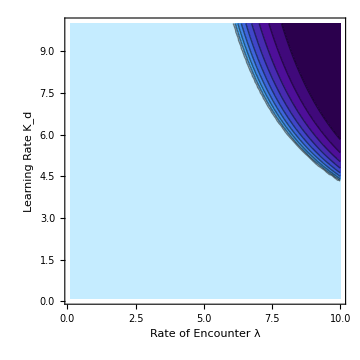

```mathematica
data=Flatten[<<"datakdλcL1",1];
kdλcL1=ListContourPlot[data,Contours->Table[c,{c,0.1,0.9,0.1}],Frame->{{True,True},{True,True}},FrameStyle->Directive[Thick,Black,14],ImageSize->Medium,FrameLabel->{Text[Style["Rate of Encounter λ",Black,20]],Text[Style["Learning Rate K_d",Black,20]]},ColorFunction->("DeepSeaColors")]
```

#### Δ = .05; Row 1

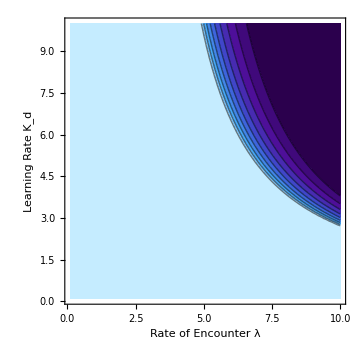

```mathematica
data=Flatten[<<"datakdλcL2",1];
kdλcL2=ListContourPlot[data,Contours->Table[c,{c,0.1,0.9,0.1}],Frame->{{True,True},{True,True}},FrameStyle->Directive[Thick,Black,14],ImageSize->Medium,FrameLabel->{Text[Style["Rate of Encounter λ",Black,20]],Text[Style["Learning Rate K_d",Black,20]]},ColorFunction->("DeepSeaColors")]
```

#### Δ = .08; Row 1

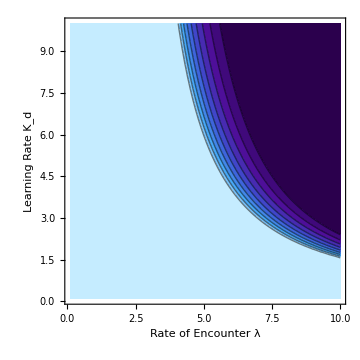

```mathematica
data=Flatten[<<"datakdλcL3",1];
kdλcL3=ListContourPlot[data,Contours->Table[c,{c,0.1,0.9,0.1}],Frame->{{True,True},{True,True}},FrameStyle->Directive[Thick,Black,14],ImageSize->Medium,FrameLabel->{Text[Style["Rate of Encounter λ",Black,20]],Text[Style["Learning Rate K_d",Black,20]]},ColorFunction->("DeepSeaColors")]
```

### Row 2

#### Δ = .02; Row 2

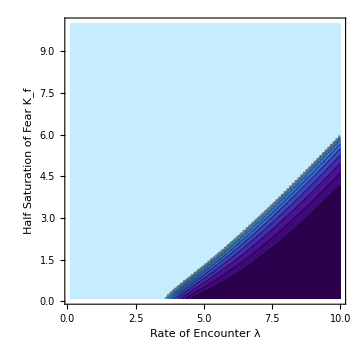

```mathematica
data=Flatten[<<"datakfλcL1",1];
kfλcL1=ListContourPlot[data,Contours->Table[c,{c,0.1,0.9,0.1}],Frame->{{True,True},{True,True}},FrameStyle->Directive[Thick,Black,14],ImageSize->Medium,FrameLabel->{Text[Style["Rate of Encounter λ",Black,20]],Text[Style["Half Saturation of Fear K_f",Black,20]]},ColorFunction->("DeepSeaColors")]
```

#### Δ = .05; Row 2

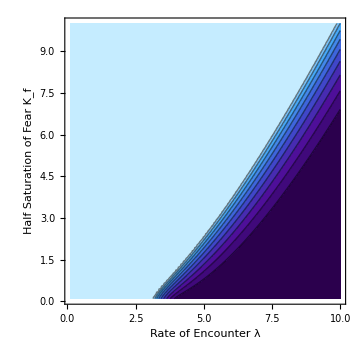

```mathematica
data=Flatten[<<"datakfλcL2",1];
kfλcL2=ListContourPlot[data,Contours->Table[c,{c,0.1,0.9,0.1}],Frame->{{True,True},{True,True}},FrameStyle->Directive[Thick,Black,14],ImageSize->Medium,FrameLabel->{Text[Style["Rate of Encounter λ",Black,20]],Text[Style["Half Saturation of Fear K_f",Black,20]]},ColorFunction->("DeepSeaColors")]
```

#### Δ = .08; Row 2

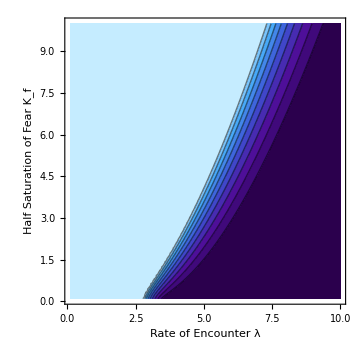

```mathematica
data=Flatten[<<"datakfλcL3",1];
kfλcL3=ListContourPlot[data,Contours->Table[c,{c,0.1,0.9,0.1}],Frame->{{True,True},{True,True}},FrameStyle->Directive[Thick,Black,14],ImageSize->Medium,FrameLabel->{Text[Style["Rate of Encounter λ",Black,20]],Text[Style["Half Saturation of Fear K_f",Black,20]]},ColorFunction->("DeepSeaColors")]
```

### Grid

```mathematica
cLgrid=Grid[{{Text[Style["   Δ 0.02",20,TextAlignment->Center]],Text[Style["    Δ 0.05",20,TextAlignment->Center]],Text[Style["     Δ 0.08",20,TextAlignment->Center]]},{kdλcL3,kdλcL2,kdλcL1},{kfλcL3,kfλcL2,kfλcL1}}]
```

Δ 0.02 |     Δ 0.05 |      Δ 0.08
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-

## Figure 4

### Data Points

```mathematica
(*data ran on cluster to expedite run time. Functions are copied below the data points for replication purposes*)
```

#### Δ = .08; Row 1

```mathematica
data = {{{0.1,0.1,0.},{0.1,0.2,0.},{0.1,0.30000000000000004,0.},{0.1,0.4,0.},{0.1,0.5,0.},{0.1,0.6,0.},{0.1,0.7000000000000001,0.},{0.1,0.8,0.},{0.1,0.9,0.},{0.1,1.,0.},{0.1,1.1,0.},{0.1,1.2000000000000002,0.},{0.1,1.3000000000000003,0.},{0.1,1.4000000000000001,0.},{0.1,1.5000000000000002,0.},{0.1,1.6,0.},{0.1,1.7000000000000002,0.},{0.1,1.8000000000000003,0.},{0.1,1.9000000000000001,0.},{0.1,2.,0.},{0.1,2.1,0.},{0.1,2.2,0.},{0.1,2.3000000000000003,0.},{0.1,2.4000000000000004,0.},{0.1,2.5000000000000004,0.},{0.1,2.6,0.},{0.1,2.7,0.},{0.1,2.8000000000000003,0.},{0.1,2.9000000000000004,0.},{0.1,3.0000000000000004,0.},{0.1,3.1,0.},{0.1,3.2,0.},{0.1,3.3000000000000003,0.},{0.1,3.4000000000000004,0.},{0.1,3.5000000000000004,0.},{0.1,3.6,0.},{0.1,3.7,0.},{0.1,3.8000000000000003,0.},{0.1,3.9000000000000004,0.},{0.1,4.,0.},{0.1,4.1,0.},{0.1,4.2,0.},{0.1,4.3,0.},{0.1,4.3999999999999995,0.},{0.1,4.5,0.},{0.1,4.6,0.},{0.1,4.7,0.},{0.1,4.8,0.},{0.1,4.9,0.},{0.1,5.,0.},{0.1,5.1,0.},{0.1,5.2,0.},{0.1,5.3,0.},{0.1,5.4,0.},{0.1,5.5,0.},{0.1,5.6,0.},{0.1,5.7,0.},{0.1,5.8,0.},{0.1,5.9,0.},{0.1,6.,0.},{0.1,6.1,0.},{0.1,6.2,0.},{0.1,6.3,0.},{0.1,6.4,0.},{0.1,6.5,0.},{0.1,6.6,0.},{0.1,6.7,0.},{0.1,6.8,0.},{0.1,6.9,0.},{0.1,7.,0.},{0.1,7.1,0.},{0.1,7.2,0.},{0.1,7.3,0.},{0.1,7.4,0.},{0.1,7.5,0.},{0.1,7.6,0.},{0.1,7.7,0.},{0.1,7.8,0.},{0.1,7.9,0.},{0.1,8.,0.},{0.1,8.1,0.},{0.1,8.2,0.},{0.1,8.3,0.},{0.1,8.4,0.},{0.1,8.5,0.},{0.1,8.6,0.},{0.1,8.7,0.},{0.1,8.8,0.},{0.1,8.9,0.},{0.1,9.,0.},{0.1,9.1,0.},{0.1,9.2,0.},{0.1,9.3,0.},{0.1,9.4,0.},{0.1,9.5,0.},{0.1,9.6,0.},{0.1,9.700000000000001,0.},{0.1,9.8,0.},{0.1,9.9,0.},{0.1,10.,0.}},{{0.2,0.1,0.},{0.2,0.2,0.},{0.2,0.30000000000000004,0.},{0.2,0.4,0.},{0.2,0.5,0.},{0.2,0.6,0.},{0.2,0.7000000000000001,0.},{0.2,0.8,0.},{0.2,0.9,0.},{0.2,1.,0.},{0.2,1.1,0.},{0.2,1.2000000000000002,0.},{0.2,1.3000000000000003,0.},{0.2,1.4000000000000001,0.},{0.2,1.5000000000000002,0.},{0.2,1.6,0.},{0.2,1.7000000000000002,0.},{0.2,1.8000000000000003,0.},{0.2,1.9000000000000001,0.},{0.2,2.,0.},{0.2,2.1,0.},{0.2,2.2,0.},{0.2,2.3000000000000003,0.},{0.2,2.4000000000000004,0.},{0.2,2.5000000000000004,0.},{0.2,2.6,0.},{0.2,2.7,0.},{0.2,2.8000000000000003,0.},{0.2,2.9000000000000004,0.},{0.2,3.0000000000000004,0.},{0.2,3.1,0.},{0.2,3.2,0.},{0.2,3.3000000000000003,0.},{0.2,3.4000000000000004,0.},{0.2,3.5000000000000004,0.},{0.2,3.6,0.},{0.2,3.7,0.},{0.2,3.8000000000000003,0.},{0.2,3.9000000000000004,0.},{0.2,4.,0.},{0.2,4.1,0.},{0.2,4.2,0.},{0.2,4.3,0.},{0.2,4.3999999999999995,0.},{0.2,4.5,0.},{0.2,4.6,0.},{0.2,4.7,0.},{0.2,4.8,0.},{0.2,4.9,0.},{0.2,5.,0.},{0.2,5.1,0.},{0.2,5.2,0.},{0.2,5.3,0.},{0.2,5.4,0.},{0.2,5.5,0.},{0.2,5.6,0.},{0.2,5.7,0.},{0.2,5.8,0.},{0.2,5.9,0.},{0.2,6.,0.},{0.2,6.1,0.},{0.2,6.2,0.},{0.2,6.3,0.},{0.2,6.4,0.},{0.2,6.5,0.},{0.2,6.6,0.},{0.2,6.7,0.},{0.2,6.8,0.},{0.2,6.9,0.},{0.2,7.,0.},{0.2,7.1,0.},{0.2,7.2,0.},{0.2,7.3,0.034095828012224494},{0.2,7.4,0.08472351649479921},{0.2,7.5,0.13404342387433932},{0.2,7.6,0.1821096344085582},{0.2,7.7,0.2289715262478303},{0.2,7.8,0.27467579817321713},{0.2,7.9,0.319266923033369},{0.2,8.,0.36278690226712546},{0.2,8.1,0.4052756352105847},{0.2,8.2,0.4467709797777062},{0.2,8.3,0.4873088822752489},{0.2,8.4,0.526923517419943},{0.2,8.5,0.5656473934447309},{0.2,8.6,0.603511459132327},{0.2,8.7,0.6405452244968922},{0.2,8.8,0.6767766495343894},{0.2,8.9,0.7122326787117935},{0.2,9.,0.746938812368594},{0.2,9.1,0.7809195075011546},{0.2,9.2,0.814198133596795},{0.2,9.3,0.8467967480475407},{0.2,9.4,0.87873700649663},{0.2,9.5,0.9100389016575993},{0.2,9.6,0.9407230067017004},{0.2,9.700000000000001,0.9708066738986377},{0.2,9.8,1.},{0.2,9.9,1.},{0.2,10.,1.}},{{0.30000000000000004,0.1,0.},{0.30000000000000004,0.2,0.},{0.30000000000000004,0.30000000000000004,0.},{0.30000000000000004,0.4,0.},{0.30000000000000004,0.5,0.},{0.30000000000000004,0.6,0.},{0.30000000000000004,0.7000000000000001,0.},{0.30000000000000004,0.8,0.},{0.30000000000000004,0.9,0.},{0.30000000000000004,1.,0.},{0.30000000000000004,1.1,0.},{0.30000000000000004,1.2000000000000002,0.},{0.30000000000000004,1.3000000000000003,0.},{0.30000000000000004,1.4000000000000001,0.},{0.30000000000000004,1.5000000000000002,0.},{0.30000000000000004,1.6,0.},{0.30000000000000004,1.7000000000000002,0.},{0.30000000000000004,1.8000000000000003,0.},{0.30000000000000004,1.9000000000000001,0.},{0.30000000000000004,2.,0.},{0.30000000000000004,2.1,0.},{0.30000000000000004,2.2,0.},{0.30000000000000004,2.3000000000000003,0.},{0.30000000000000004,2.4000000000000004,0.},{0.30000000000000004,2.5000000000000004,0.},{0.30000000000000004,2.6,0.},{0.30000000000000004,2.7,0.},{0.30000000000000004,2.8000000000000003,0.},{0.30000000000000004,2.9000000000000004,0.},{0.30000000000000004,3.0000000000000004,0.},{0.30000000000000004,3.1,0.},{0.30000000000000004,3.2,0.},{0.30000000000000004,3.3000000000000003,0.},{0.30000000000000004,3.4000000000000004,0.},{0.30000000000000004,3.5000000000000004,0.},{0.30000000000000004,3.6,0.},{0.30000000000000004,3.7,0.},{0.30000000000000004,3.8000000000000003,0.},{0.30000000000000004,3.9000000000000004,0.},{0.30000000000000004,4.,0.},{0.30000000000000004,4.1,0.},{0.30000000000000004,4.2,0.},{0.30000000000000004,4.3,0.},{0.30000000000000004,4.3999999999999995,0.},{0.30000000000000004,4.5,0.},{0.30000000000000004,4.6,0.},{0.30000000000000004,4.7,0.},{0.30000000000000004,4.8,0.},{0.30000000000000004,4.9,0.05072485159718592},{0.30000000000000004,5.,0.12873394121832948},{0.30000000000000004,5.1,0.2036317885826577},{0.30000000000000004,5.2,0.2756099251328896},{0.30000000000000004,5.3,0.3448439576912007},{0.30000000000000004,5.4,0.41149536571781586},{0.30000000000000004,5.5,0.47571259682740047},{0.30000000000000004,5.6,0.5376329007813033},{0.30000000000000004,5.7,0.59738287172581},{0.30000000000000004,5.8,0.6550797325772362},{0.30000000000000004,5.9,0.7108322196757982},{0.30000000000000004,6.,0.7647411412671044},{0.30000000000000004,6.1,0.8169003391688889},{0.30000000000000004,6.2,0.8673971570205942},{0.30000000000000004,6.3,0.9163128099203246},{0.30000000000000004,6.4,0.9637238063687731},{0.30000000000000004,6.5,1.},{0.30000000000000004,6.6,1.},{0.30000000000000004,6.7,1.},{0.30000000000000004,6.8,1.},{0.30000000000000004,6.9,1.},{0.30000000000000004,7.,1.},{0.30000000000000004,7.1,1.},{0.30000000000000004,7.2,1.},{0.30000000000000004,7.3,1.},{0.30000000000000004,7.4,1.},{0.30000000000000004,7.5,1.},{0.30000000000000004,7.6,1.},{0.30000000000000004,7.7,1.},{0.30000000000000004,7.8,1.},{0.30000000000000004,7.9,1.},{0.30000000000000004,8.,1.},{0.30000000000000004,8.1,1.},{0.30000000000000004,8.2,1.},{0.30000000000000004,8.3,1.},{0.30000000000000004,8.4,1.},{0.30000000000000004,8.5,1.},{0.30000000000000004,8.6,1.},{0.30000000000000004,8.7,1.},{0.30000000000000004,8.8,1.},{0.30000000000000004,8.9,1.},{0.30000000000000004,9.,1.},{0.30000000000000004,9.1,1.},{0.30000000000000004,9.2,1.},{0.30000000000000004,9.3,1.},{0.30000000000000004,9.4,1.},{0.30000000000000004,9.5,1.},{0.30000000000000004,9.6,1.},{0.30000000000000004,9.700000000000001,1.},{0.30000000000000004,9.8,1.},{0.30000000000000004,9.9,1.},{0.30000000000000004,10.,1.}},{{0.4,0.1,0.},{0.4,0.2,0.},{0.4,0.30000000000000004,0.},{0.4,0.4,0.},{0.4,0.5,0.},{0.4,0.6,0.},{0.4,0.7000000000000001,0.},{0.4,0.8,0.},{0.4,0.9,0.},{0.4,1.,0.},{0.4,1.1,0.},{0.4,1.2000000000000002,0.},{0.4,1.3000000000000003,0.},{0.4,1.4000000000000001,0.},{0.4,1.5000000000000002,0.},{0.4,1.6,0.},{0.4,1.7000000000000002,0.},{0.4,1.8000000000000003,0.},{0.4,1.9000000000000001,0.},{0.4,2.,0.},{0.4,2.1,0.},{0.4,2.2,0.},{0.4,2.3000000000000003,0.},{0.4,2.4000000000000004,0.},{0.4,2.5000000000000004,0.},{0.4,2.6,0.},{0.4,2.7,0.},{0.4,2.8000000000000003,0.},{0.4,2.9000000000000004,0.},{0.4,3.0000000000000004,0.},{0.4,3.1,0.},{0.4,3.2,0.},{0.4,3.3000000000000003,0.},{0.4,3.4000000000000004,0.},{0.4,3.5000000000000004,0.},{0.4,3.6,0.},{0.4,3.7,0.08457999425846564},{0.4,3.8000000000000003,0.19076026381407557},{0.4,3.9000000000000004,0.2911349382129584},{0.4,4.,0.3861888951654568},{0.4,4.1,0.47635302087800835},{0.4,4.2,0.5620116730594631},{0.4,4.3,0.6435090508717815},{0.4,4.3999999999999995,0.7211540584631991},{0.4,4.5,0.7952250064716664},{0.4,4.6,0.8659734926557793},{0.4,4.7,0.9336272197537238},{0.4,4.8,0.9983915580901314},{0.4,4.9,1.},{0.4,5.,1.},{0.4,5.1,1.},{0.4,5.2,1.},{0.4,5.3,1.},{0.4,5.4,1.},{0.4,5.5,1.},{0.4,5.6,1.},{0.4,5.7,1.},{0.4,5.8,1.},{0.4,5.9,1.},{0.4,6.,1.},{0.4,6.1,1.},{0.4,6.2,1.},{0.4,6.3,1.},{0.4,6.4,1.},{0.4,6.5,1.},{0.4,6.6,1.},{0.4,6.7,1.},{0.4,6.8,1.},{0.4,6.9,1.},{0.4,7.,1.},{0.4,7.1,1.},{0.4,7.2,1.},{0.4,7.3,1.},{0.4,7.4,1.},{0.4,7.5,1.},{0.4,7.6,1.},{0.4,7.7,1.},{0.4,7.8,1.},{0.4,7.9,1.},{0.4,8.,1.},{0.4,8.1,1.},{0.4,8.2,1.},{0.4,8.3,1.},{0.4,8.4,1.},{0.4,8.5,1.},{0.4,8.6,1.},{0.4,8.7,1.},{0.4,8.8,1.},{0.4,8.9,1.},{0.4,9.,1.},{0.4,9.1,1.},{0.4,9.2,1.},{0.4,9.3,1.},{0.4,9.4,1.},{0.4,9.5,1.},{0.4,9.6,1.},{0.4,9.700000000000001,1.},{0.4,9.8,1.},{0.4,9.9,1.},{0.4,10.,1.}},{{0.5,0.1,0.},{0.5,0.2,0.},{0.5,0.30000000000000004,0.},{0.5,0.4,0.},{0.5,0.5,0.},{0.5,0.6,0.},{0.5,0.7000000000000001,0.},{0.5,0.8,0.},{0.5,0.9,0.},{0.5,1.,0.},{0.5,1.1,0.},{0.5,1.2000000000000002,0.},{0.5,1.3000000000000003,0.},{0.5,1.4000000000000001,0.},{0.5,1.5000000000000002,0.},{0.5,1.6,0.},{0.5,1.7000000000000002,0.},{0.5,1.8000000000000003,0.},{0.5,1.9000000000000001,0.},{0.5,2.,0.},{0.5,2.1,0.},{0.5,2.2,0.},{0.5,2.3000000000000003,0.},{0.5,2.4000000000000004,0.},{0.5,2.5000000000000004,0.},{0.5,2.6,0.},{0.5,2.7,0.},{0.5,2.8000000000000003,0.},{0.5,2.9000000000000004,0.012403961228909242},{0.5,3.0000000000000004,0.15572889983885604},{0.5,3.1,0.28864405040196556},{0.5,3.2,0.412293943551906},{0.5,3.3000000000000003,0.5276525850215842},{0.5,3.4000000000000004,0.6355661227226184},{0.5,3.5000000000000004,0.7367622293553963},{0.5,3.6,0.8318754558410323},{0.5,3.7,0.9214608487269055},{0.5,3.8000000000000003,1.},{0.5,3.9000000000000004,1.},{0.5,4.,1.},{0.5,4.1,1.},{0.5,4.2,1.},{0.5,4.3,1.},{0.5,4.3999999999999995,1.},{0.5,4.5,1.},{0.5,4.6,1.},{0.5,4.7,1.},{0.5,4.8,1.},{0.5,4.9,1.},{0.5,5.,1.},{0.5,5.1,1.},{0.5,5.2,1.},{0.5,5.3,1.},{0.5,5.4,1.},{0.5,5.5,1.},{0.5,5.6,1.},{0.5,5.7,1.},{0.5,5.8,1.},{0.5,5.9,1.},{0.5,6.,1.},{0.5,6.1,1.},{0.5,6.2,1.},{0.5,6.3,1.},{0.5,6.4,1.},{0.5,6.5,1.},{0.5,6.6,1.},{0.5,6.7,1.},{0.5,6.8,1.},{0.5,6.9,1.},{0.5,7.,1.},{0.5,7.1,1.},{0.5,7.2,1.},{0.5,7.3,1.},{0.5,7.4,1.},{0.5,7.5,1.},{0.5,7.6,1.},{0.5,7.7,1.},{0.5,7.8,1.},{0.5,7.9,1.},{0.5,8.,1.},{0.5,8.1,1.},{0.5,8.2,1.},{0.5,8.3,1.},{0.5,8.4,1.},{0.5,8.5,1.},{0.5,8.6,1.},{0.5,8.7,1.},{0.5,8.8,1.},{0.5,8.9,1.},{0.5,9.,1.},{0.5,9.1,1.},{0.5,9.2,1.},{0.5,9.3,1.},{0.5,9.4,1.},{0.5,9.5,1.},{0.5,9.6,1.},{0.5,9.700000000000001,1.},{0.5,9.8,1.},{0.5,9.9,1.},{0.5,10.,1.}},{{0.6000000000000001,0.1,0.},{0.6000000000000001,0.2,0.},{0.6000000000000001,0.30000000000000004,0.},{0.6000000000000001,0.4,0.},{0.6000000000000001,0.5,0.},{0.6000000000000001,0.6,0.},{0.6000000000000001,0.7000000000000001,0.},{0.6000000000000001,0.8,0.},{0.6000000000000001,0.9,0.},{0.6000000000000001,1.,0.},{0.6000000000000001,1.1,0.},{0.6000000000000001,1.2000000000000002,0.},{0.6000000000000001,1.3000000000000003,0.},{0.6000000000000001,1.4000000000000001,0.},{0.6000000000000001,1.5000000000000002,0.},{0.6000000000000001,1.6,0.},{0.6000000000000001,1.7000000000000002,0.},{0.6000000000000001,1.8000000000000003,0.},{0.6000000000000001,1.9000000000000001,0.},{0.6000000000000001,2.,0.},{0.6000000000000001,2.1,0.},{0.6000000000000001,2.2,0.},{0.6000000000000001,2.3000000000000003,0.},{0.6000000000000001,2.4000000000000004,0.000015841109842321402},{0.6000000000000001,2.5000000000000004,0.17778512536406613},{0.6000000000000001,2.6,0.34167546946541305},{0.6000000000000001,2.7,0.4913537464150893},{0.6000000000000001,2.8000000000000003,0.6286731510570267},{0.6000000000000001,2.9000000000000004,0.7551707566245114},{0.6000000000000001,3.0000000000000004,0.8721336602092001},{0.6000000000000001,3.1,0.980644831169591},{0.6000000000000001,3.2,1.},{0.6000000000000001,3.3000000000000003,1.},{0.6000000000000001,3.4000000000000004,1.},{0.6000000000000001,3.5000000000000004,1.},{0.6000000000000001,3.6,1.},{0.6000000000000001,3.7,1.},{0.6000000000000001,3.8000000000000003,1.},{0.6000000000000001,3.9000000000000004,1.},{0.6000000000000001,4.,1.},{0.6000000000000001,4.1,1.},{0.6000000000000001,4.2,1.},{0.6000000000000001,4.3,1.},{0.6000000000000001,4.3999999999999995,1.},{0.6000000000000001,4.5,1.},{0.6000000000000001,4.6,1.},{0.6000000000000001,4.7,1.},{0.6000000000000001,4.8,1.},{0.6000000000000001,4.9,1.},{0.6000000000000001,5.,1.},{0.6000000000000001,5.1,1.},{0.6000000000000001,5.2,1.},{0.6000000000000001,5.3,1.},{0.6000000000000001,5.4,1.},{0.6000000000000001,5.5,1.},{0.6000000000000001,5.6,1.},{0.6000000000000001,5.7,1.},{0.6000000000000001,5.8,1.},{0.6000000000000001,5.9,1.},{0.6000000000000001,6.,1.},{0.6000000000000001,6.1,1.},{0.6000000000000001,6.2,1.},{0.6000000000000001,6.3,1.},{0.6000000000000001,6.4,1.},{0.6000000000000001,6.5,1.},{0.6000000000000001,6.6,1.},{0.6000000000000001,6.7,1.},{0.6000000000000001,6.8,1.},{0.6000000000000001,6.9,1.},{0.6000000000000001,7.,1.},{0.6000000000000001,7.1,1.},{0.6000000000000001,7.2,1.},{0.6000000000000001,7.3,1.},{0.6000000000000001,7.4,1.},{0.6000000000000001,7.5,1.},{0.6000000000000001,7.6,1.},{0.6000000000000001,7.7,1.},{0.6000000000000001,7.8,1.},{0.6000000000000001,7.9,1.},{0.6000000000000001,8.,1.},{0.6000000000000001,8.1,1.},{0.6000000000000001,8.2,1.},{0.6000000000000001,8.3,1.},{0.6000000000000001,8.4,1.},{0.6000000000000001,8.5,1.},{0.6000000000000001,8.6,1.},{0.6000000000000001,8.7,1.},{0.6000000000000001,8.8,1.},{0.6000000000000001,8.9,1.},{0.6000000000000001,9.,1.},{0.6000000000000001,9.1,1.},{0.6000000000000001,9.2,1.},{0.6000000000000001,9.3,1.},{0.6000000000000001,9.4,1.},{0.6000000000000001,9.5,1.},{0.6000000000000001,9.6,1.},{0.6000000000000001,9.700000000000001,1.},{0.6000000000000001,9.8,1.},{0.6000000000000001,9.9,1.},{0.6000000000000001,10.,1.}},{{0.7000000000000001,0.1,0.},{0.7000000000000001,0.2,0.},{0.7000000000000001,0.30000000000000004,0.},{0.7000000000000001,0.4,0.},{0.7000000000000001,0.5,0.},{0.7000000000000001,0.6,0.},{0.7000000000000001,0.7000000000000001,0.},{0.7000000000000001,0.8,0.},{0.7000000000000001,0.9,0.},{0.7000000000000001,1.,0.},{0.7000000000000001,1.1,0.},{0.7000000000000001,1.2000000000000002,0.},{0.7000000000000001,1.3000000000000003,0.},{0.7000000000000001,1.4000000000000001,0.},{0.7000000000000001,1.5000000000000002,0.},{0.7000000000000001,1.6,0.},{0.7000000000000001,1.7000000000000002,0.},{0.7000000000000001,1.8000000000000003,0.},{0.7000000000000001,1.9000000000000001,0.},{0.7000000000000001,2.,0.},{0.7000000000000001,2.1,0.11202846690787058},{0.7000000000000001,2.2,0.31802378912862084},{0.7000000000000001,2.3000000000000003,0.5018362444057878},{0.7000000000000001,2.4000000000000004,0.6670336386929202},{0.7000000000000001,2.5000000000000004,0.8164393026574036},{0.7000000000000001,2.6,0.9523188369060785},{0.7000000000000001,2.7,1.},{0.7000000000000001,2.8000000000000003,1.},{0.7000000000000001,2.9000000000000004,1.},{0.7000000000000001,3.0000000000000004,1.},{0.7000000000000001,3.1,1.},{0.7000000000000001,3.2,1.},{0.7000000000000001,3.3000000000000003,1.},{0.7000000000000001,3.4000000000000004,1.},{0.7000000000000001,3.5000000000000004,1.},{0.7000000000000001,3.6,1.},{0.7000000000000001,3.7,1.},{0.7000000000000001,3.8000000000000003,1.},{0.7000000000000001,3.9000000000000004,1.},{0.7000000000000001,4.,1.},{0.7000000000000001,4.1,1.},{0.7000000000000001,4.2,1.},{0.7000000000000001,4.3,1.},{0.7000000000000001,4.3999999999999995,1.},{0.7000000000000001,4.5,1.},{0.7000000000000001,4.6,1.},{0.7000000000000001,4.7,1.},{0.7000000000000001,4.8,1.},{0.7000000000000001,4.9,1.},{0.7000000000000001,5.,1.},{0.7000000000000001,5.1,1.},{0.7000000000000001,5.2,1.},{0.7000000000000001,5.3,1.},{0.7000000000000001,5.4,1.},{0.7000000000000001,5.5,1.},{0.7000000000000001,5.6,1.},{0.7000000000000001,5.7,1.},{0.7000000000000001,5.8,1.},{0.7000000000000001,5.9,1.},{0.7000000000000001,6.,1.},{0.7000000000000001,6.1,1.},{0.7000000000000001,6.2,1.},{0.7000000000000001,6.3,1.},{0.7000000000000001,6.4,1.},{0.7000000000000001,6.5,1.},{0.7000000000000001,6.6,1.},{0.7000000000000001,6.7,1.},{0.7000000000000001,6.8,1.},{0.7000000000000001,6.9,1.},{0.7000000000000001,7.,1.},{0.7000000000000001,7.1,1.},{0.7000000000000001,7.2,1.},{0.7000000000000001,7.3,1.},{0.7000000000000001,7.4,1.},{0.7000000000000001,7.5,1.},{0.7000000000000001,7.6,1.},{0.7000000000000001,7.7,1.},{0.7000000000000001,7.8,1.},{0.7000000000000001,7.9,1.},{0.7000000000000001,8.,1.},{0.7000000000000001,8.1,1.},{0.7000000000000001,8.2,1.},{0.7000000000000001,8.3,1.},{0.7000000000000001,8.4,1.},{0.7000000000000001,8.5,1.},{0.7000000000000001,8.6,1.},{0.7000000000000001,8.7,1.},{0.7000000000000001,8.8,1.},{0.7000000000000001,8.9,1.},{0.7000000000000001,9.,1.},{0.7000000000000001,9.1,1.},{0.7000000000000001,9.2,1.},{0.7000000000000001,9.3,1.},{0.7000000000000001,9.4,1.},{0.7000000000000001,9.5,1.},{0.7000000000000001,9.6,1.},{0.7000000000000001,9.700000000000001,1.},{0.7000000000000001,9.8,1.},{0.7000000000000001,9.9,1.},{0.7000000000000001,10.,1.}},{{0.8,0.1,0.},{0.8,0.2,0.},{0.8,0.30000000000000004,0.},{0.8,0.4,0.},{0.8,0.5,0.},{0.8,0.6,0.},{0.8,0.7000000000000001,0.},{0.8,0.8,0.},{0.8,0.9,0.},{0.8,1.,0.},{0.8,1.1,0.},{0.8,1.2000000000000002,0.},{0.8,1.3000000000000003,0.},{0.8,1.4000000000000001,0.},{0.8,1.5000000000000002,0.},{0.8,1.6,0.},{0.8,1.7000000000000002,0.},{0.8,1.8000000000000003,0.037025520674801436},{0.8,1.9000000000000001,0.2918764852678315},{0.8,2.,0.5132388931894067},{0.8,2.1,0.7076416769633997},{0.8,2.2,0.8799772494802137},{0.8,2.3000000000000003,1.},{0.8,2.4000000000000004,1.},{0.8,2.5000000000000004,1.},{0.8,2.6,1.},{0.8,2.7,1.},{0.8,2.8000000000000003,1.},{0.8,2.9000000000000004,1.},{0.8,3.0000000000000004,1.},{0.8,3.1,1.},{0.8,3.2,1.},{0.8,3.3000000000000003,1.},{0.8,3.4000000000000004,1.},{0.8,3.5000000000000004,1.},{0.8,3.6,1.},{0.8,3.7,1.},{0.8,3.8000000000000003,1.},{0.8,3.9000000000000004,1.},{0.8,4.,1.},{0.8,4.1,1.},{0.8,4.2,1.},{0.8,4.3,1.},{0.8,4.3999999999999995,1.},{0.8,4.5,1.},{0.8,4.6,1.},{0.8,4.7,1.},{0.8,4.8,1.},{0.8,4.9,1.},{0.8,5.,1.},{0.8,5.1,1.},{0.8,5.2,1.},{0.8,5.3,1.},{0.8,5.4,1.},{0.8,5.5,1.},{0.8,5.6,1.},{0.8,5.7,1.},{0.8,5.8,1.},{0.8,5.9,1.},{0.8,6.,1.},{0.8,6.1,1.},{0.8,6.2,1.},{0.8,6.3,1.},{0.8,6.4,1.},{0.8,6.5,1.},{0.8,6.6,1.},{0.8,6.7,1.},{0.8,6.8,1.},{0.8,6.9,1.},{0.8,7.,1.},{0.8,7.1,1.},{0.8,7.2,1.},{0.8,7.3,1.},{0.8,7.4,1.},{0.8,7.5,1.},{0.8,7.6,1.},{0.8,7.7,1.},{0.8,7.8,1.},{0.8,7.9,1.},{0.8,8.,1.},{0.8,8.1,1.},{0.8,8.2,1.},{0.8,8.3,1.},{0.8,8.4,1.},{0.8,8.5,1.},{0.8,8.6,1.},{0.8,8.7,1.},{0.8,8.8,1.},{0.8,8.9,1.},{0.8,9.,1.},{0.8,9.1,1.},{0.8,9.2,1.},{0.8,9.3,1.},{0.8,9.4,1.},{0.8,9.5,1.},{0.8,9.6,1.},{0.8,9.700000000000001,1.},{0.8,9.8,1.},{0.8,9.9,1.},{0.8,10.,1.}},{{0.9000000000000001,0.1,0.},{0.9000000000000001,0.2,0.},{0.9000000000000001,0.30000000000000004,0.},{0.9000000000000001,0.4,0.},{0.9000000000000001,0.5,0.},{0.9000000000000001,0.6,0.},{0.9000000000000001,0.7000000000000001,0.},{0.9000000000000001,0.8,0.},{0.9000000000000001,0.9,0.},{0.9000000000000001,1.,0.},{0.9000000000000001,1.1,0.},{0.9000000000000001,1.2000000000000002,0.},{0.9000000000000001,1.3000000000000003,0.},{0.9000000000000001,1.4000000000000001,0.},{0.9000000000000001,1.5000000000000002,0.},{0.9000000000000001,1.6,0.06058005701893986},{0.9000000000000001,1.7000000000000002,0.35480936262905094},{0.9000000000000001,1.8000000000000003,0.6039078377526281},{0.9000000000000001,1.9000000000000001,0.818095771012223},{0.9000000000000001,2.,1.},{0.9000000000000001,2.1,1.},{0.9000000000000001,2.2,1.},{0.9000000000000001,2.3000000000000003,1.},{0.9000000000000001,2.4000000000000004,1.},{0.9000000000000001,2.5000000000000004,1.},{0.9000000000000001,2.6,1.},{0.9000000000000001,2.7,1.},{0.9000000000000001,2.8000000000000003,1.},{0.9000000000000001,2.9000000000000004,1.},{0.9000000000000001,3.0000000000000004,1.},{0.9000000000000001,3.1,1.},{0.9000000000000001,3.2,1.},{0.9000000000000001,3.3000000000000003,1.},{0.9000000000000001,3.4000000000000004,1.},{0.9000000000000001,3.5000000000000004,1.},{0.9000000000000001,3.6,1.},{0.9000000000000001,3.7,1.},{0.9000000000000001,3.8000000000000003,1.},{0.9000000000000001,3.9000000000000004,1.},{0.9000000000000001,4.,1.},{0.9000000000000001,4.1,1.},{0.9000000000000001,4.2,1.},{0.9000000000000001,4.3,1.},{0.9000000000000001,4.3999999999999995,1.},{0.9000000000000001,4.5,1.},{0.9000000000000001,4.6,1.},{0.9000000000000001,4.7,1.},{0.9000000000000001,4.8,1.},{0.9000000000000001,4.9,1.},{0.9000000000000001,5.,1.},{0.9000000000000001,5.1,1.},{0.9000000000000001,5.2,1.},{0.9000000000000001,5.3,1.},{0.9000000000000001,5.4,1.},{0.9000000000000001,5.5,1.},{0.9000000000000001,5.6,1.},{0.9000000000000001,5.7,1.},{0.9000000000000001,5.8,1.},{0.9000000000000001,5.9,1.},{0.9000000000000001,6.,1.},{0.9000000000000001,6.1,1.},{0.9000000000000001,6.2,1.},{0.9000000000000001,6.3,1.},{0.9000000000000001,6.4,1.},{0.9000000000000001,6.5,1.},{0.9000000000000001,6.6,1.},{0.9000000000000001,6.7,1.},{0.9000000000000001,6.8,1.},{0.9000000000000001,6.9,1.},{0.9000000000000001,7.,1.},{0.9000000000000001,7.1,1.},{0.9000000000000001,7.2,1.},{0.9000000000000001,7.3,1.},{0.9000000000000001,7.4,1.},{0.9000000000000001,7.5,1.},{0.9000000000000001,7.6,1.},{0.9000000000000001,7.7,1.},{0.9000000000000001,7.8,1.},{0.9000000000000001,7.9,1.},{0.9000000000000001,8.,1.},{0.9000000000000001,8.1,1.},{0.9000000000000001,8.2,1.},{0.9000000000000001,8.3,1.},{0.9000000000000001,8.4,1.},{0.9000000000000001,8.5,1.},{0.9000000000000001,8.6,1.},{0.9000000000000001,8.7,1.},{0.9000000000000001,8.8,1.},{0.9000000000000001,8.9,1.},{0.9000000000000001,9.,1.},{0.9000000000000001,9.1,1.},{0.9000000000000001,9.2,1.},{0.9000000000000001,9.3,1.},{0.9000000000000001,9.4,1.},{0.9000000000000001,9.5,1.},{0.9000000000000001,9.6,1.},{0.9000000000000001,9.700000000000001,1.},{0.9000000000000001,9.8,1.},{0.9000000000000001,9.9,1.},{0.9000000000000001,10.,1.}},{{1.,0.1,0.},{1.,0.2,0.},{1.,0.30000000000000004,0.},{1.,0.4,0.},{1.,0.5,0.},{1.,0.6,0.},{1.,0.7000000000000001,0.},{1.,0.8,0.},{1.,0.9,0.},{1.,1.,0.},{1.,1.1,0.},{1.,1.2000000000000002,0.},{1.,1.3000000000000003,0.},{1.,1.4000000000000001,0.},{1.,1.5000000000000002,0.29539617474474844},{1.,1.6,0.5924547094867281},{1.,1.7000000000000002,0.8403738224308905},{1.,1.8000000000000003,1.},{1.,1.9000000000000001,1.},{1.,2.,1.},{1.,2.1,1.},{1.,2.2,1.},{1.,2.3000000000000003,1.},{1.,2.4000000000000004,1.},{1.,2.5000000000000004,1.},{1.,2.6,1.},{1.,2.7,1.},{1.,2.8000000000000003,1.},{1.,2.9000000000000004,1.},{1.,3.0000000000000004,1.},{1.,3.1,1.},{1.,3.2,1.},{1.,3.3000000000000003,1.},{1.,3.4000000000000004,1.},{1.,3.5000000000000004,1.},{1.,3.6,1.},{1.,3.7,1.},{1.,3.8000000000000003,1.},{1.,3.9000000000000004,1.},{1.,4.,1.},{1.,4.1,1.},{1.,4.2,1.},{1.,4.3,1.},{1.,4.3999999999999995,1.},{1.,4.5,1.},{1.,4.6,1.},{1.,4.7,1.},{1.,4.8,1.},{1.,4.9,1.},{1.,5.,1.},{1.,5.1,1.},{1.,5.2,1.},{1.,5.3,1.},{1.,5.4,1.},{1.,5.5,1.},{1.,5.6,1.},{1.,5.7,1.},{1.,5.8,1.},{1.,5.9,1.},{1.,6.,1.},{1.,6.1,1.},{1.,6.2,1.},{1.,6.3,1.},{1.,6.4,1.},{1.,6.5,1.},{1.,6.6,1.},{1.,6.7,1.},{1.,6.8,1.},{1.,6.9,1.},{1.,7.,1.},{1.,7.1,1.},{1.,7.2,1.},{1.,7.3,1.},{1.,7.4,1.},{1.,7.5,1.},{1.,7.6,1.},{1.,7.7,1.},{1.,7.8,1.},{1.,7.9,1.},{1.,8.,1.},{1.,8.1,1.},{1.,8.2,1.},{1.,8.3,1.},{1.,8.4,1.},{1.,8.5,1.},{1.,8.6,1.},{1.,8.7,1.},{1.,8.8,1.},{1.,8.9,1.},{1.,9.,1.},{1.,9.1,1.},{1.,9.2,1.},{1.,9.3,1.},{1.,9.4,1.},{1.,9.5,1.},{1.,9.6,1.},{1.,9.700000000000001,1.},{1.,9.8,1.},{1.,9.9,1.},{1.,10.,1.}},{{1.1,0.1,0.},{1.1,0.2,0.},{1.1,0.30000000000000004,0.},{1.1,0.4,0.},{1.1,0.5,0.},{1.1,0.6,0.},{1.1,0.7000000000000001,0.},{1.1,0.8,0.},{1.1,0.9,0.},{1.1,1.,0.},{1.1,1.1,0.},{1.1,1.2000000000000002,0.},{1.1,1.3000000000000003,0.07529359430624287},{1.1,1.4000000000000001,0.4597631930954177},{1.1,1.5000000000000002,0.766136615202782},{1.1,1.6,1.},{1.1,1.7000000000000002,1.},{1.1,1.8000000000000003,1.},{1.1,1.9000000000000001,1.},{1.1,2.,1.},{1.1,2.1,1.},{1.1,2.2,1.},{1.1,2.3000000000000003,1.},{1.1,2.4000000000000004,1.},{1.1,2.5000000000000004,1.},{1.1,2.6,1.},{1.1,2.7,1.},{1.1,2.8000000000000003,1.},{1.1,2.9000000000000004,1.},{1.1,3.0000000000000004,1.},{1.1,3.1,1.},{1.1,3.2,1.},{1.1,3.3000000000000003,1.},{1.1,3.4000000000000004,1.},{1.1,3.5000000000000004,1.},{1.1,3.6,1.},{1.1,3.7,1.},{1.1,3.8000000000000003,1.},{1.1,3.9000000000000004,1.},{1.1,4.,1.},{1.1,4.1,1.},{1.1,4.2,1.},{1.1,4.3,1.},{1.1,4.3999999999999995,1.},{1.1,4.5,1.},{1.1,4.6,1.},{1.1,4.7,1.},{1.1,4.8,1.},{1.1,4.9,1.},{1.1,5.,1.},{1.1,5.1,1.},{1.1,5.2,1.},{1.1,5.3,1.},{1.1,5.4,1.},{1.1,5.5,1.},{1.1,5.6,1.},{1.1,5.7,1.},{1.1,5.8,1.},{1.1,5.9,1.},{1.1,6.,1.},{1.1,6.1,1.},{1.1,6.2,1.},{1.1,6.3,1.},{1.1,6.4,1.},{1.1,6.5,1.},{1.1,6.6,1.},{1.1,6.7,1.},{1.1,6.8,1.},{1.1,6.9,1.},{1.1,7.,1.},{1.1,7.1,1.},{1.1,7.2,1.},{1.1,7.3,1.},{1.1,7.4,1.},{1.1,7.5,1.},{1.1,7.6,1.},{1.1,7.7,1.},{1.1,7.8,1.},{1.1,7.9,1.},{1.1,8.,1.},{1.1,8.1,1.},{1.1,8.2,1.},{1.1,8.3,1.},{1.1,8.4,1.},{1.1,8.5,1.},{1.1,8.6,1.},{1.1,8.7,1.},{1.1,8.8,1.},{1.1,8.9,1.},{1.1,9.,1.},{1.1,9.1,1.},{1.1,9.2,1.},{1.1,9.3,1.},{1.1,9.4,1.},{1.1,9.5,1.},{1.1,9.6,1.},{1.1,9.700000000000001,1.},{1.1,9.8,1.},{1.1,9.9,1.},{1.1,10.,1.}},{{1.2,0.1,0.},{1.2,0.2,0.},{1.2,0.30000000000000004,0.},{1.2,0.4,0.},{1.2,0.5,0.},{1.2,0.6,0.},{1.2,0.7000000000000001,0.},{1.2,0.8,0.},{1.2,0.9,0.},{1.2,1.,0.},{1.2,1.1,0.},{1.2,1.2000000000000002,0.14452276829846766},{1.2,1.3000000000000003,0.5623875445791015},{1.2,1.4000000000000001,0.8859741860794118},{1.2,1.5000000000000002,1.},{1.2,1.6,1.},{1.2,1.7000000000000002,1.},{1.2,1.8000000000000003,1.},{1.2,1.9000000000000001,1.},{1.2,2.,1.},{1.2,2.1,1.},{1.2,2.2,1.},{1.2,2.3000000000000003,1.},{1.2,2.4000000000000004,1.},{1.2,2.5000000000000004,1.},{1.2,2.6,1.},{1.2,2.7,1.},{1.2,2.8000000000000003,1.},{1.2,2.9000000000000004,1.},{1.2,3.0000000000000004,1.},{1.2,3.1,1.},{1.2,3.2,1.},{1.2,3.3000000000000003,1.},{1.2,3.4000000000000004,1.},{1.2,3.5000000000000004,1.},{1.2,3.6,1.},{1.2,3.7,1.},{1.2,3.8000000000000003,1.},{1.2,3.9000000000000004,1.},{1.2,4.,1.},{1.2,4.1,1.},{1.2,4.2,1.},{1.2,4.3,1.},{1.2,4.3999999999999995,1.},{1.2,4.5,1.},{1.2,4.6,1.},{1.2,4.7,1.},{1.2,4.8,1.},{1.2,4.9,1.},{1.2,5.,1.},{1.2,5.1,1.},{1.2,5.2,1.},{1.2,5.3,1.},{1.2,5.4,1.},{1.2,5.5,1.},{1.2,5.6,1.},{1.2,5.7,1.},{1.2,5.8,1.},{1.2,5.9,1.},{1.2,6.,1.},{1.2,6.1,1.},{1.2,6.2,1.},{1.2,6.3,1.},{1.2,6.4,1.},{1.2,6.5,1.},{1.2,6.6,1.},{1.2,6.7,1.},{1.2,6.8,1.},{1.2,6.9,1.},{1.2,7.,1.},{1.2,7.1,1.},{1.2,7.2,1.},{1.2,7.3,1.},{1.2,7.4,1.},{1.2,7.5,1.},{1.2,7.6,1.},{1.2,7.7,1.},{1.2,7.8,1.},{1.2,7.9,1.},{1.2,8.,1.},{1.2,8.1,1.},{1.2,8.2,1.},{1.2,8.3,1.},{1.2,8.4,1.},{1.2,8.5,1.},{1.2,8.6,1.},{1.2,8.7,1.},{1.2,8.8,1.},{1.2,8.9,1.},{1.2,9.,1.},{1.2,9.1,1.},{1.2,9.2,1.},{1.2,9.3,1.},{1.2,9.4,1.},{1.2,9.5,1.},{1.2,9.6,1.},{1.2,9.700000000000001,1.},{1.2,9.8,1.},{1.2,9.9,1.},{1.2,10.,1.}},{{1.3000000000000003,0.1,0.},{1.3000000000000003,0.2,0.},{1.3000000000000003,0.30000000000000004,0.},{1.3000000000000003,0.4,0.},{1.3000000000000003,0.5,0.},{1.3000000000000003,0.6,0.},{1.3000000000000003,0.7000000000000001,0.},{1.3000000000000003,0.8,0.},{1.3000000000000003,0.9,0.},{1.3000000000000003,1.,0.},{1.3000000000000003,1.1,0.13482913464278193},{1.3000000000000003,1.2000000000000002,0.6061449644285912},{1.3000000000000003,1.3000000000000003,0.9575016771835867},{1.3000000000000003,1.4000000000000001,1.},{1.3000000000000003,1.5000000000000002,1.},{1.3000000000000003,1.6,1.},{1.3000000000000003,1.7000000000000002,1.},{1.3000000000000003,1.8000000000000003,1.},{1.3000000000000003,1.9000000000000001,1.},{1.3000000000000003,2.,1.},{1.3000000000000003,2.1,1.},{1.3000000000000003,2.2,1.},{1.3000000000000003,2.3000000000000003,1.},{1.3000000000000003,2.4000000000000004,1.},{1.3000000000000003,2.5000000000000004,1.},{1.3000000000000003,2.6,1.},{1.3000000000000003,2.7,1.},{1.3000000000000003,2.8000000000000003,1.},{1.3000000000000003,2.9000000000000004,1.},{1.3000000000000003,3.0000000000000004,1.},{1.3000000000000003,3.1,1.},{1.3000000000000003,3.2,1.},{1.3000000000000003,3.3000000000000003,1.},{1.3000000000000003,3.4000000000000004,1.},{1.3000000000000003,3.5000000000000004,1.},{1.3000000000000003,3.6,1.},{1.3000000000000003,3.7,1.},{1.3000000000000003,3.8000000000000003,1.},{1.3000000000000003,3.9000000000000004,1.},{1.3000000000000003,4.,1.},{1.3000000000000003,4.1,1.},{1.3000000000000003,4.2,1.},{1.3000000000000003,4.3,1.},{1.3000000000000003,4.3999999999999995,1.},{1.3000000000000003,4.5,1.},{1.3000000000000003,4.6,1.},{1.3000000000000003,4.7,1.},{1.3000000000000003,4.8,1.},{1.3000000000000003,4.9,1.},{1.3000000000000003,5.,1.},{1.3000000000000003,5.1,1.},{1.3000000000000003,5.2,1.},{1.3000000000000003,5.3,1.},{1.3000000000000003,5.4,1.},{1.3000000000000003,5.5,1.},{1.3000000000000003,5.6,1.},{1.3000000000000003,5.7,1.},{1.3000000000000003,5.8,1.},{1.3000000000000003,5.9,1.},{1.3000000000000003,6.,1.},{1.3000000000000003,6.1,1.},{1.3000000000000003,6.2,1.},{1.3000000000000003,6.3,1.},{1.3000000000000003,6.4,1.},{1.3000000000000003,6.5,1.},{1.3000000000000003,6.6,1.},{1.3000000000000003,6.7,1.},{1.3000000000000003,6.8,1.},{1.3000000000000003,6.9,1.},{1.3000000000000003,7.,1.},{1.3000000000000003,7.1,1.},{1.3000000000000003,7.2,1.},{1.3000000000000003,7.3,1.},{1.3000000000000003,7.4,1.},{1.3000000000000003,7.5,1.},{1.3000000000000003,7.6,1.},{1.3000000000000003,7.7,1.},{1.3000000000000003,7.8,1.},{1.3000000000000003,7.9,1.},{1.3000000000000003,8.,1.},{1.3000000000000003,8.1,1.},{1.3000000000000003,8.2,1.},{1.3000000000000003,8.3,1.},{1.3000000000000003,8.4,1.},{1.3000000000000003,8.5,1.},{1.3000000000000003,8.6,1.},{1.3000000000000003,8.7,1.},{1.3000000000000003,8.8,1.},{1.3000000000000003,8.9,1.},{1.3000000000000003,9.,1.},{1.3000000000000003,9.1,1.},{1.3000000000000003,9.2,1.},{1.3000000000000003,9.3,1.},{1.3000000000000003,9.4,1.},{1.3000000000000003,9.5,1.},{1.3000000000000003,9.6,1.},{1.3000000000000003,9.700000000000001,1.},{1.3000000000000003,9.8,1.},{1.3000000000000003,9.9,1.},{1.3000000000000003,10.,1.}},{{1.4000000000000004,0.1,0.},{1.4000000000000004,0.2,0.},{1.4000000000000004,0.30000000000000004,0.},{1.4000000000000004,0.4,0.},{1.4000000000000004,0.5,0.},{1.4000000000000004,0.6,0.},{1.4000000000000004,0.7000000000000001,0.},{1.4000000000000004,0.8,0.},{1.4000000000000004,0.9,0.},{1.4000000000000004,1.,0.028630190481555746},{1.4000000000000004,1.1,0.5874269145016627},{1.4000000000000004,1.2000000000000002,0.9820938066317703},{1.4000000000000004,1.3000000000000003,1.},{1.4000000000000004,1.4000000000000001,1.},{1.4000000000000004,1.5000000000000002,1.},{1.4000000000000004,1.6,1.},{1.4000000000000004,1.7000000000000002,1.},{1.4000000000000004,1.8000000000000003,1.},{1.4000000000000004,1.9000000000000001,1.},{1.4000000000000004,2.,1.},{1.4000000000000004,2.1,1.},{1.4000000000000004,2.2,1.},{1.4000000000000004,2.3000000000000003,1.},{1.4000000000000004,2.4000000000000004,1.},{1.4000000000000004,2.5000000000000004,1.},{1.4000000000000004,2.6,1.},{1.4000000000000004,2.7,1.},{1.4000000000000004,2.8000000000000003,1.},{1.4000000000000004,2.9000000000000004,1.},{1.4000000000000004,3.0000000000000004,1.},{1.4000000000000004,3.1,1.},{1.4000000000000004,3.2,1.},{1.4000000000000004,3.3000000000000003,1.},{1.4000000000000004,3.4000000000000004,1.},{1.4000000000000004,3.5000000000000004,1.},{1.4000000000000004,3.6,1.},{1.4000000000000004,3.7,1.},{1.4000000000000004,3.8000000000000003,1.},{1.4000000000000004,3.9000000000000004,1.},{1.4000000000000004,4.,1.},{1.4000000000000004,4.1,1.},{1.4000000000000004,4.2,1.},{1.4000000000000004,4.3,1.},{1.4000000000000004,4.3999999999999995,1.},{1.4000000000000004,4.5,1.},{1.4000000000000004,4.6,1.},{1.4000000000000004,4.7,1.},{1.4000000000000004,4.8,1.},{1.4000000000000004,4.9,1.},{1.4000000000000004,5.,1.},{1.4000000000000004,5.1,1.},{1.4000000000000004,5.2,1.},{1.4000000000000004,5.3,1.},{1.4000000000000004,5.4,1.},{1.4000000000000004,5.5,1.},{1.4000000000000004,5.6,1.},{1.4000000000000004,5.7,1.},{1.4000000000000004,5.8,1.},{1.4000000000000004,5.9,1.},{1.4000000000000004,6.,1.},{1.4000000000000004,6.1,1.},{1.4000000000000004,6.2,1.},{1.4000000000000004,6.3,1.},{1.4000000000000004,6.4,1.},{1.4000000000000004,6.5,1.},{1.4000000000000004,6.6,1.},{1.4000000000000004,6.7,1.},{1.4000000000000004,6.8,1.},{1.4000000000000004,6.9,1.},{1.4000000000000004,7.,1.},{1.4000000000000004,7.1,1.},{1.4000000000000004,7.2,1.},{1.4000000000000004,7.3,1.},{1.4000000000000004,7.4,1.},{1.4000000000000004,7.5,1.},{1.4000000000000004,7.6,1.},{1.4000000000000004,7.7,1.},{1.4000000000000004,7.8,1.},{1.4000000000000004,7.9,1.},{1.4000000000000004,8.,1.},{1.4000000000000004,8.1,1.},{1.4000000000000004,8.2,1.},{1.4000000000000004,8.3,1.},{1.4000000000000004,8.4,1.},{1.4000000000000004,8.5,1.},{1.4000000000000004,8.6,1.},{1.4000000000000004,8.7,1.},{1.4000000000000004,8.8,1.},{1.4000000000000004,8.9,1.},{1.4000000000000004,9.,1.},{1.4000000000000004,9.1,1.},{1.4000000000000004,9.2,1.},{1.4000000000000004,9.3,1.},{1.4000000000000004,9.4,1.},{1.4000000000000004,9.5,1.},{1.4000000000000004,9.6,1.},{1.4000000000000004,9.700000000000001,1.},{1.4000000000000004,9.8,1.},{1.4000000000000004,9.9,1.},{1.4000000000000004,10.,1.}},{{1.5000000000000002,0.1,0.},{1.5000000000000002,0.2,0.},{1.5000000000000002,0.30000000000000004,0.},{1.5000000000000002,0.4,0.},{1.5000000000000002,0.5,0.},{1.5000000000000002,0.6,0.},{1.5000000000000002,0.7000000000000001,0.},{1.5000000000000002,0.8,0.},{1.5000000000000002,0.9,0.},{1.5000000000000002,1.,0.49283085796564957},{1.5000000000000002,1.1,0.956333318957436},{1.5000000000000002,1.2000000000000002,1.},{1.5000000000000002,1.3000000000000003,1.},{1.5000000000000002,1.4000000000000001,1.},{1.5000000000000002,1.5000000000000002,1.},{1.5000000000000002,1.6,1.},{1.5000000000000002,1.7000000000000002,1.},{1.5000000000000002,1.8000000000000003,1.},{1.5000000000000002,1.9000000000000001,1.},{1.5000000000000002,2.,1.},{1.5000000000000002,2.1,1.},{1.5000000000000002,2.2,1.},{1.5000000000000002,2.3000000000000003,1.},{1.5000000000000002,2.4000000000000004,1.},{1.5000000000000002,2.5000000000000004,1.},{1.5000000000000002,2.6,1.},{1.5000000000000002,2.7,1.},{1.5000000000000002,2.8000000000000003,1.},{1.5000000000000002,2.9000000000000004,1.},{1.5000000000000002,3.0000000000000004,1.},{1.5000000000000002,3.1,1.},{1.5000000000000002,3.2,1.},{1.5000000000000002,3.3000000000000003,1.},{1.5000000000000002,3.4000000000000004,1.},{1.5000000000000002,3.5000000000000004,1.},{1.5000000000000002,3.6,1.},{1.5000000000000002,3.7,1.},{1.5000000000000002,3.8000000000000003,1.},{1.5000000000000002,3.9000000000000004,1.},{1.5000000000000002,4.,1.},{1.5000000000000002,4.1,1.},{1.5000000000000002,4.2,1.},{1.5000000000000002,4.3,1.},{1.5000000000000002,4.3999999999999995,1.},{1.5000000000000002,4.5,1.},{1.5000000000000002,4.6,1.},{1.5000000000000002,4.7,1.},{1.5000000000000002,4.8,1.},{1.5000000000000002,4.9,1.},{1.5000000000000002,5.,1.},{1.5000000000000002,5.1,1.},{1.5000000000000002,5.2,1.},{1.5000000000000002,5.3,1.},{1.5000000000000002,5.4,1.},{1.5000000000000002,5.5,1.},{1.5000000000000002,5.6,1.},{1.5000000000000002,5.7,1.},{1.5000000000000002,5.8,1.},{1.5000000000000002,5.9,1.},{1.5000000000000002,6.,1.},{1.5000000000000002,6.1,1.},{1.5000000000000002,6.2,1.},{1.5000000000000002,6.3,1.},{1.5000000000000002,6.4,1.},{1.5000000000000002,6.5,1.},{1.5000000000000002,6.6,1.},{1.5000000000000002,6.7,1.},{1.5000000000000002,6.8,1.},{1.5000000000000002,6.9,1.},{1.5000000000000002,7.,1.},{1.5000000000000002,7.1,1.},{1.5000000000000002,7.2,1.},{1.5000000000000002,7.3,1.},{1.5000000000000002,7.4,1.},{1.5000000000000002,7.5,1.},{1.5000000000000002,7.6,1.},{1.5000000000000002,7.7,1.},{1.5000000000000002,7.8,1.},{1.5000000000000002,7.9,1.},{1.5000000000000002,8.,1.},{1.5000000000000002,8.1,1.},{1.5000000000000002,8.2,1.},{1.5000000000000002,8.3,1.},{1.5000000000000002,8.4,1.},{1.5000000000000002,8.5,1.},{1.5000000000000002,8.6,1.},{1.5000000000000002,8.7,1.},{1.5000000000000002,8.8,1.},{1.5000000000000002,8.9,1.},{1.5000000000000002,9.,1.},{1.5000000000000002,9.1,1.},{1.5000000000000002,9.2,1.},{1.5000000000000002,9.3,1.},{1.5000000000000002,9.4,1.},{1.5000000000000002,9.5,1.},{1.5000000000000002,9.6,1.},{1.5000000000000002,9.700000000000001,1.},{1.5000000000000002,9.8,1.},{1.5000000000000002,9.9,1.},{1.5000000000000002,10.,1.}},{{1.6,0.1,0.},{1.6,0.2,0.},{1.6,0.30000000000000004,0.},{1.6,0.4,0.},{1.6,0.5,0.},{1.6,0.6,0.},{1.6,0.7000000000000001,0.},{1.6,0.8,0.},{1.6,0.9,0.28885755770447963},{1.6,1.,0.8695903349276048},{1.6,1.1,1.},{1.6,1.2000000000000002,1.},{1.6,1.3000000000000003,1.},{1.6,1.4000000000000001,1.},{1.6,1.5000000000000002,1.},{1.6,1.6,1.},{1.6,1.7000000000000002,1.},{1.6,1.8000000000000003,1.},{1.6,1.9000000000000001,1.},{1.6,2.,1.},{1.6,2.1,1.},{1.6,2.2,1.},{1.6,2.3000000000000003,1.},{1.6,2.4000000000000004,1.},{1.6,2.5000000000000004,1.},{1.6,2.6,1.},{1.6,2.7,1.},{1.6,2.8000000000000003,1.},{1.6,2.9000000000000004,1.},{1.6,3.0000000000000004,1.},{1.6,3.1,1.},{1.6,3.2,1.},{1.6,3.3000000000000003,1.},{1.6,3.4000000000000004,1.},{1.6,3.5000000000000004,1.},{1.6,3.6,1.},{1.6,3.7,1.},{1.6,3.8000000000000003,1.},{1.6,3.9000000000000004,1.},{1.6,4.,1.},{1.6,4.1,1.},{1.6,4.2,1.},{1.6,4.3,1.},{1.6,4.3999999999999995,1.},{1.6,4.5,1.},{1.6,4.6,1.},{1.6,4.7,1.},{1.6,4.8,1.},{1.6,4.9,1.},{1.6,5.,1.},{1.6,5.1,1.},{1.6,5.2,1.},{1.6,5.3,1.},{1.6,5.4,1.},{1.6,5.5,1.},{1.6,5.6,1.},{1.6,5.7,1.},{1.6,5.8,1.},{1.6,5.9,1.},{1.6,6.,1.},{1.6,6.1,1.},{1.6,6.2,1.},{1.6,6.3,1.},{1.6,6.4,1.},{1.6,6.5,1.},{1.6,6.6,1.},{1.6,6.7,1.},{1.6,6.8,1.},{1.6,6.9,1.},{1.6,7.,1.},{1.6,7.1,1.},{1.6,7.2,1.},{1.6,7.3,1.},{1.6,7.4,1.},{1.6,7.5,1.},{1.6,7.6,1.},{1.6,7.7,1.},{1.6,7.8,1.},{1.6,7.9,1.},{1.6,8.,1.},{1.6,8.1,1.},{1.6,8.2,1.},{1.6,8.3,1.},{1.6,8.4,1.},{1.6,8.5,1.},{1.6,8.6,1.},{1.6,8.7,1.},{1.6,8.8,1.},{1.6,8.9,1.},{1.6,9.,1.},{1.6,9.1,1.},{1.6,9.2,1.},{1.6,9.3,1.},{1.6,9.4,1.},{1.6,9.5,1.},{1.6,9.6,1.},{1.6,9.700000000000001,1.},{1.6,9.8,1.},{1.6,9.9,1.},{1.6,10.,1.}},{{1.7000000000000002,0.1,0.},{1.7000000000000002,0.2,0.},{1.7000000000000002,0.30000000000000004,0.},{1.7000000000000002,0.4,0.},{1.7000000000000002,0.5,0.},{1.7000000000000002,0.6,0.},{1.7000000000000002,0.7000000000000001,0.},{1.7000000000000002,0.8,0.},{1.7000000000000002,0.9,0.6970785541735993},{1.7000000000000002,1.,1.},{1.7000000000000002,1.1,1.},{1.7000000000000002,1.2000000000000002,1.},{1.7000000000000002,1.3000000000000003,1.},{1.7000000000000002,1.4000000000000001,1.},{1.7000000000000002,1.5000000000000002,1.},{1.7000000000000002,1.6,1.},{1.7000000000000002,1.7000000000000002,1.},{1.7000000000000002,1.8000000000000003,1.},{1.7000000000000002,1.9000000000000001,1.},{1.7000000000000002,2.,1.},{1.7000000000000002,2.1,1.},{1.7000000000000002,2.2,1.},{1.7000000000000002,2.3000000000000003,1.},{1.7000000000000002,2.4000000000000004,1.},{1.7000000000000002,2.5000000000000004,1.},{1.7000000000000002,2.6,1.},{1.7000000000000002,2.7,1.},{1.7000000000000002,2.8000000000000003,1.},{1.7000000000000002,2.9000000000000004,1.},{1.7000000000000002,3.0000000000000004,1.},{1.7000000000000002,3.1,1.},{1.7000000000000002,3.2,1.},{1.7000000000000002,3.3000000000000003,1.},{1.7000000000000002,3.4000000000000004,1.},{1.7000000000000002,3.5000000000000004,1.},{1.7000000000000002,3.6,1.},{1.7000000000000002,3.7,1.},{1.7000000000000002,3.8000000000000003,1.},{1.7000000000000002,3.9000000000000004,1.},{1.7000000000000002,4.,1.},{1.7000000000000002,4.1,1.},{1.7000000000000002,4.2,1.},{1.7000000000000002,4.3,1.},{1.7000000000000002,4.3999999999999995,1.},{1.7000000000000002,4.5,1.},{1.7000000000000002,4.6,1.},{1.7000000000000002,4.7,1.},{1.7000000000000002,4.8,1.},{1.7000000000000002,4.9,1.},{1.7000000000000002,5.,1.},{1.7000000000000002,5.1,1.},{1.7000000000000002,5.2,1.},{1.7000000000000002,5.3,1.},{1.7000000000000002,5.4,1.},{1.7000000000000002,5.5,1.},{1.7000000000000002,5.6,1.},{1.7000000000000002,5.7,1.},{1.7000000000000002,5.8,1.},{1.7000000000000002,5.9,1.},{1.7000000000000002,6.,1.},{1.7000000000000002,6.1,1.},{1.7000000000000002,6.2,1.},{1.7000000000000002,6.3,1.},{1.7000000000000002,6.4,1.},{1.7000000000000002,6.5,1.},{1.7000000000000002,6.6,1.},{1.7000000000000002,6.7,1.},{1.7000000000000002,6.8,1.},{1.7000000000000002,6.9,1.},{1.7000000000000002,7.,1.},{1.7000000000000002,7.1,1.},{1.7000000000000002,7.2,1.},{1.7000000000000002,7.3,1.},{1.7000000000000002,7.4,1.},{1.7000000000000002,7.5,1.},{1.7000000000000002,7.6,1.},{1.7000000000000002,7.7,1.},{1.7000000000000002,7.8,1.},{1.7000000000000002,7.9,1.},{1.7000000000000002,8.,1.},{1.7000000000000002,8.1,1.},{1.7000000000000002,8.2,1.},{1.7000000000000002,8.3,1.},{1.7000000000000002,8.4,1.},{1.7000000000000002,8.5,1.},{1.7000000000000002,8.6,1.},{1.7000000000000002,8.7,1.},{1.7000000000000002,8.8,1.},{1.7000000000000002,8.9,1.},{1.7000000000000002,9.,1.},{1.7000000000000002,9.1,1.},{1.7000000000000002,9.2,1.},{1.7000000000000002,9.3,1.},{1.7000000000000002,9.4,1.},{1.7000000000000002,9.5,1.},{1.7000000000000002,9.6,1.},{1.7000000000000002,9.700000000000001,1.},{1.7000000000000002,9.8,1.},{1.7000000000000002,9.9,1.},{1.7000000000000002,10.,1.}},{{1.8,0.1,0.},{1.8,0.2,0.},{1.8,0.30000000000000004,0.},{1.8,0.4,0.},{1.8,0.5,0.},{1.8,0.6,0.},{1.8,0.7000000000000001,0.},{1.8,0.8,0.37682116613787353},{1.8,0.9,1.},{1.8,1.,1.},{1.8,1.1,1.},{1.8,1.2000000000000002,1.},{1.8,1.3000000000000003,1.},{1.8,1.4000000000000001,1.},{1.8,1.5000000000000002,1.},{1.8,1.6,1.},{1.8,1.7000000000000002,1.},{1.8,1.8000000000000003,1.},{1.8,1.9000000000000001,1.},{1.8,2.,1.},{1.8,2.1,1.},{1.8,2.2,1.},{1.8,2.3000000000000003,1.},{1.8,2.4000000000000004,1.},{1.8,2.5000000000000004,1.},{1.8,2.6,1.},{1.8,2.7,1.},{1.8,2.8000000000000003,1.},{1.8,2.9000000000000004,1.},{1.8,3.0000000000000004,1.},{1.8,3.1,1.},{1.8,3.2,1.},{1.8,3.3000000000000003,1.},{1.8,3.4000000000000004,1.},{1.8,3.5000000000000004,1.},{1.8,3.6,1.},{1.8,3.7,1.},{1.8,3.8000000000000003,1.},{1.8,3.9000000000000004,1.},{1.8,4.,1.},{1.8,4.1,1.},{1.8,4.2,1.},{1.8,4.3,1.},{1.8,4.3999999999999995,1.},{1.8,4.5,1.},{1.8,4.6,1.},{1.8,4.7,1.},{1.8,4.8,1.},{1.8,4.9,1.},{1.8,5.,1.},{1.8,5.1,1.},{1.8,5.2,1.},{1.8,5.3,1.},{1.8,5.4,1.},{1.8,5.5,1.},{1.8,5.6,1.},{1.8,5.7,1.},{1.8,5.8,1.},{1.8,5.9,1.},{1.8,6.,1.},{1.8,6.1,1.},{1.8,6.2,1.},{1.8,6.3,1.},{1.8,6.4,1.},{1.8,6.5,1.},{1.8,6.6,1.},{1.8,6.7,1.},{1.8,6.8,1.},{1.8,6.9,1.},{1.8,7.,1.},{1.8,7.1,1.},{1.8,7.2,1.},{1.8,7.3,1.},{1.8,7.4,1.},{1.8,7.5,1.},{1.8,7.6,1.},{1.8,7.7,1.},{1.8,7.8,1.},{1.8,7.9,1.},{1.8,8.,1.},{1.8,8.1,1.},{1.8,8.2,1.},{1.8,8.3,1.},{1.8,8.4,1.},{1.8,8.5,1.},{1.8,8.6,1.},{1.8,8.7,1.},{1.8,8.8,1.},{1.8,8.9,1.},{1.8,9.,1.},{1.8,9.1,1.},{1.8,9.2,1.},{1.8,9.3,1.},{1.8,9.4,1.},{1.8,9.5,1.},{1.8,9.6,1.},{1.8,9.700000000000001,1.},{1.8,9.8,1.},{1.8,9.9,1.},{1.8,10.,1.}},{{1.9000000000000001,0.1,0.},{1.9000000000000001,0.2,0.},{1.9000000000000001,0.30000000000000004,0.},{1.9000000000000001,0.4,0.},{1.9000000000000001,0.5,0.},{1.9000000000000001,0.6,0.},{1.9000000000000001,0.7000000000000001,0.},{1.9000000000000001,0.8,0.7652874001812067},{1.9000000000000001,0.9,1.},{1.9000000000000001,1.,1.},{1.9000000000000001,1.1,1.},{1.9000000000000001,1.2000000000000002,1.},{1.9000000000000001,1.3000000000000003,1.},{1.9000000000000001,1.4000000000000001,1.},{1.9000000000000001,1.5000000000000002,1.},{1.9000000000000001,1.6,1.},{1.9000000000000001,1.7000000000000002,1.},{1.9000000000000001,1.8000000000000003,1.},{1.9000000000000001,1.9000000000000001,1.},{1.9000000000000001,2.,1.},{1.9000000000000001,2.1,1.},{1.9000000000000001,2.2,1.},{1.9000000000000001,2.3000000000000003,1.},{1.9000000000000001,2.4000000000000004,1.},{1.9000000000000001,2.5000000000000004,1.},{1.9000000000000001,2.6,1.},{1.9000000000000001,2.7,1.},{1.9000000000000001,2.8000000000000003,1.},{1.9000000000000001,2.9000000000000004,1.},{1.9000000000000001,3.0000000000000004,1.},{1.9000000000000001,3.1,1.},{1.9000000000000001,3.2,1.},{1.9000000000000001,3.3000000000000003,1.},{1.9000000000000001,3.4000000000000004,1.},{1.9000000000000001,3.5000000000000004,1.},{1.9000000000000001,3.6,1.},{1.9000000000000001,3.7,1.},{1.9000000000000001,3.8000000000000003,1.},{1.9000000000000001,3.9000000000000004,1.},{1.9000000000000001,4.,1.},{1.9000000000000001,4.1,1.},{1.9000000000000001,4.2,1.},{1.9000000000000001,4.3,1.},{1.9000000000000001,4.3999999999999995,1.},{1.9000000000000001,4.5,1.},{1.9000000000000001,4.6,1.},{1.9000000000000001,4.7,1.},{1.9000000000000001,4.8,1.},{1.9000000000000001,4.9,1.},{1.9000000000000001,5.,1.},{1.9000000000000001,5.1,1.},{1.9000000000000001,5.2,1.},{1.9000000000000001,5.3,1.},{1.9000000000000001,5.4,1.},{1.9000000000000001,5.5,1.},{1.9000000000000001,5.6,1.},{1.9000000000000001,5.7,1.},{1.9000000000000001,5.8,1.},{1.9000000000000001,5.9,1.},{1.9000000000000001,6.,1.},{1.9000000000000001,6.1,1.},{1.9000000000000001,6.2,1.},{1.9000000000000001,6.3,1.},{1.9000000000000001,6.4,1.},{1.9000000000000001,6.5,1.},{1.9000000000000001,6.6,1.},{1.9000000000000001,6.7,1.},{1.9000000000000001,6.8,1.},{1.9000000000000001,6.9,1.},{1.9000000000000001,7.,1.},{1.9000000000000001,7.1,1.},{1.9000000000000001,7.2,1.},{1.9000000000000001,7.3,1.},{1.9000000000000001,7.4,1.},{1.9000000000000001,7.5,1.},{1.9000000000000001,7.6,1.},{1.9000000000000001,7.7,1.},{1.9000000000000001,7.8,1.},{1.9000000000000001,7.9,1.},{1.9000000000000001,8.,1.},{1.9000000000000001,8.1,1.},{1.9000000000000001,8.2,1.},{1.9000000000000001,8.3,1.},{1.9000000000000001,8.4,1.},{1.9000000000000001,8.5,1.},{1.9000000000000001,8.6,1.},{1.9000000000000001,8.7,1.},{1.9000000000000001,8.8,1.},{1.9000000000000001,8.9,1.},{1.9000000000000001,9.,1.},{1.9000000000000001,9.1,1.},{1.9000000000000001,9.2,1.},{1.9000000000000001,9.3,1.},{1.9000000000000001,9.4,1.},{1.9000000000000001,9.5,1.},{1.9000000000000001,9.6,1.},{1.9000000000000001,9.700000000000001,1.},{1.9000000000000001,9.8,1.},{1.9000000000000001,9.9,1.},{1.9000000000000001,10.,1.}},{{2.,0.1,0.},{2.,0.2,0.},{2.,0.30000000000000004,0.},{2.,0.4,0.},{2.,0.5,0.},{2.,0.6,0.},{2.,0.7000000000000001,0.2532965856318881},{2.,0.8,1.},{2.,0.9,1.},{2.,1.,1.},{2.,1.1,1.},{2.,1.2000000000000002,1.},{2.,1.3000000000000003,1.},{2.,1.4000000000000001,1.},{2.,1.5000000000000002,1.},{2.,1.6,1.},{2.,1.7000000000000002,1.},{2.,1.8000000000000003,1.},{2.,1.9000000000000001,1.},{2.,2.,1.},{2.,2.1,1.},{2.,2.2,1.},{2.,2.3000000000000003,1.},{2.,2.4000000000000004,1.},{2.,2.5000000000000004,1.},{2.,2.6,1.},{2.,2.7,1.},{2.,2.8000000000000003,1.},{2.,2.9000000000000004,1.},{2.,3.0000000000000004,1.},{2.,3.1,1.},{2.,3.2,1.},{2.,3.3000000000000003,1.},{2.,3.4000000000000004,1.},{2.,3.5000000000000004,1.},{2.,3.6,1.},{2.,3.7,1.},{2.,3.8000000000000003,1.},{2.,3.9000000000000004,1.},{2.,4.,1.},{2.,4.1,1.},{2.,4.2,1.},{2.,4.3,1.},{2.,4.3999999999999995,1.},{2.,4.5,1.},{2.,4.6,1.},{2.,4.7,1.},{2.,4.8,1.},{2.,4.9,1.},{2.,5.,1.},{2.,5.1,1.},{2.,5.2,1.},{2.,5.3,1.},{2.,5.4,1.},{2.,5.5,1.},{2.,5.6,1.},{2.,5.7,1.},{2.,5.8,1.},{2.,5.9,1.},{2.,6.,1.},{2.,6.1,1.},{2.,6.2,1.},{2.,6.3,1.},{2.,6.4,1.},{2.,6.5,1.},{2.,6.6,1.},{2.,6.7,1.},{2.,6.8,1.},{2.,6.9,1.},{2.,7.,1.},{2.,7.1,1.},{2.,7.2,1.},{2.,7.3,1.},{2.,7.4,1.},{2.,7.5,1.},{2.,7.6,1.},{2.,7.7,1.},{2.,7.8,1.},{2.,7.9,1.},{2.,8.,1.},{2.,8.1,1.},{2.,8.2,1.},{2.,8.3,1.},{2.,8.4,1.},{2.,8.5,1.},{2.,8.6,1.},{2.,8.7,1.},{2.,8.8,1.},{2.,8.9,1.},{2.,9.,1.},{2.,9.1,1.},{2.,9.2,1.},{2.,9.3,1.},{2.,9.4,1.},{2.,9.5,1.},{2.,9.6,1.},{2.,9.700000000000001,1.},{2.,9.8,1.},{2.,9.9,1.},{2.,10.,1.}},{{2.1,0.1,0.},{2.1,0.2,0.},{2.1,0.30000000000000004,0.},{2.1,0.4,0.},{2.1,0.5,0.},{2.1,0.6,0.},{2.1,0.7000000000000001,0.6742061010881458},{2.1,0.8,1.},{2.1,0.9,1.},{2.1,1.,1.},{2.1,1.1,1.},{2.1,1.2000000000000002,1.},{2.1,1.3000000000000003,1.},{2.1,1.4000000000000001,1.},{2.1,1.5000000000000002,1.},{2.1,1.6,1.},{2.1,1.7000000000000002,1.},{2.1,1.8000000000000003,1.},{2.1,1.9000000000000001,1.},{2.1,2.,1.},{2.1,2.1,1.},{2.1,2.2,1.},{2.1,2.3000000000000003,1.},{2.1,2.4000000000000004,1.},{2.1,2.5000000000000004,1.},{2.1,2.6,1.},{2.1,2.7,1.},{2.1,2.8000000000000003,1.},{2.1,2.9000000000000004,1.},{2.1,3.0000000000000004,1.},{2.1,3.1,1.},{2.1,3.2,1.},{2.1,3.3000000000000003,1.},{2.1,3.4000000000000004,1.},{2.1,3.5000000000000004,1.},{2.1,3.6,1.},{2.1,3.7,1.},{2.1,3.8000000000000003,1.},{2.1,3.9000000000000004,1.},{2.1,4.,1.},{2.1,4.1,1.},{2.1,4.2,1.},{2.1,4.3,1.},{2.1,4.3999999999999995,1.},{2.1,4.5,1.},{2.1,4.6,1.},{2.1,4.7,1.},{2.1,4.8,1.},{2.1,4.9,1.},{2.1,5.,1.},{2.1,5.1,1.},{2.1,5.2,1.},{2.1,5.3,1.},{2.1,5.4,1.},{2.1,5.5,1.},{2.1,5.6,1.},{2.1,5.7,1.},{2.1,5.8,1.},{2.1,5.9,1.},{2.1,6.,1.},{2.1,6.1,1.},{2.1,6.2,1.},{2.1,6.3,1.},{2.1,6.4,1.},{2.1,6.5,1.},{2.1,6.6,1.},{2.1,6.7,1.},{2.1,6.8,1.},{2.1,6.9,1.},{2.1,7.,1.},{2.1,7.1,1.},{2.1,7.2,1.},{2.1,7.3,1.},{2.1,7.4,1.},{2.1,7.5,1.},{2.1,7.6,1.},{2.1,7.7,1.},{2.1,7.8,1.},{2.1,7.9,1.},{2.1,8.,1.},{2.1,8.1,1.},{2.1,8.2,1.},{2.1,8.3,1.},{2.1,8.4,1.},{2.1,8.5,1.},{2.1,8.6,1.},{2.1,8.7,1.},{2.1,8.8,1.},{2.1,8.9,1.},{2.1,9.,1.},{2.1,9.1,1.},{2.1,9.2,1.},{2.1,9.3,1.},{2.1,9.4,1.},{2.1,9.5,1.},{2.1,9.6,1.},{2.1,9.700000000000001,1.},{2.1,9.8,1.},{2.1,9.9,1.},{2.1,10.,1.}},{{2.2,0.1,0.},{2.2,0.2,0.},{2.2,0.30000000000000004,0.},{2.2,0.4,0.},{2.2,0.5,0.},{2.2,0.6,0.},{2.2,0.7000000000000001,1.},{2.2,0.8,1.},{2.2,0.9,1.},{2.2,1.,1.},{2.2,1.1,1.},{2.2,1.2000000000000002,1.},{2.2,1.3000000000000003,1.},{2.2,1.4000000000000001,1.},{2.2,1.5000000000000002,1.},{2.2,1.6,1.},{2.2,1.7000000000000002,1.},{2.2,1.8000000000000003,1.},{2.2,1.9000000000000001,1.},{2.2,2.,1.},{2.2,2.1,1.},{2.2,2.2,1.},{2.2,2.3000000000000003,1.},{2.2,2.4000000000000004,1.},{2.2,2.5000000000000004,1.},{2.2,2.6,1.},{2.2,2.7,1.},{2.2,2.8000000000000003,1.},{2.2,2.9000000000000004,1.},{2.2,3.0000000000000004,1.},{2.2,3.1,1.},{2.2,3.2,1.},{2.2,3.3000000000000003,1.},{2.2,3.4000000000000004,1.},{2.2,3.5000000000000004,1.},{2.2,3.6,1.},{2.2,3.7,1.},{2.2,3.8000000000000003,1.},{2.2,3.9000000000000004,1.},{2.2,4.,1.},{2.2,4.1,1.},{2.2,4.2,1.},{2.2,4.3,1.},{2.2,4.3999999999999995,1.},{2.2,4.5,1.},{2.2,4.6,1.},{2.2,4.7,1.},{2.2,4.8,1.},{2.2,4.9,1.},{2.2,5.,1.},{2.2,5.1,1.},{2.2,5.2,1.},{2.2,5.3,1.},{2.2,5.4,1.},{2.2,5.5,1.},{2.2,5.6,1.},{2.2,5.7,1.},{2.2,5.8,1.},{2.2,5.9,1.},{2.2,6.,1.},{2.2,6.1,1.},{2.2,6.2,1.},{2.2,6.3,1.},{2.2,6.4,1.},{2.2,6.5,1.},{2.2,6.6,1.},{2.2,6.7,1.},{2.2,6.8,1.},{2.2,6.9,1.},{2.2,7.,1.},{2.2,7.1,1.},{2.2,7.2,1.},{2.2,7.3,1.},{2.2,7.4,1.},{2.2,7.5,1.},{2.2,7.6,1.},{2.2,7.7,1.},{2.2,7.8,1.},{2.2,7.9,1.},{2.2,8.,1.},{2.2,8.1,1.},{2.2,8.2,1.},{2.2,8.3,1.},{2.2,8.4,1.},{2.2,8.5,1.},{2.2,8.6,1.},{2.2,8.7,1.},{2.2,8.8,1.},{2.2,8.9,1.},{2.2,9.,1.},{2.2,9.1,1.},{2.2,9.2,1.},{2.2,9.3,1.},{2.2,9.4,1.},{2.2,9.5,1.},{2.2,9.6,1.},{2.2,9.700000000000001,1.},{2.2,9.8,1.},{2.2,9.9,1.},{2.2,10.,1.}},{{2.3000000000000003,0.1,0.},{2.3000000000000003,0.2,0.},{2.3000000000000003,0.30000000000000004,0.},{2.3000000000000003,0.4,0.},{2.3000000000000003,0.5,0.},{2.3000000000000003,0.6,0.27115537518272176},{2.3000000000000003,0.7000000000000001,1.},{2.3000000000000003,0.8,1.},{2.3000000000000003,0.9,1.},{2.3000000000000003,1.,1.},{2.3000000000000003,1.1,1.},{2.3000000000000003,1.2000000000000002,1.},{2.3000000000000003,1.3000000000000003,1.},{2.3000000000000003,1.4000000000000001,1.},{2.3000000000000003,1.5000000000000002,1.},{2.3000000000000003,1.6,1.},{2.3000000000000003,1.7000000000000002,1.},{2.3000000000000003,1.8000000000000003,1.},{2.3000000000000003,1.9000000000000001,1.},{2.3000000000000003,2.,1.},{2.3000000000000003,2.1,1.},{2.3000000000000003,2.2,1.},{2.3000000000000003,2.3000000000000003,1.},{2.3000000000000003,2.4000000000000004,1.},{2.3000000000000003,2.5000000000000004,1.},{2.3000000000000003,2.6,1.},{2.3000000000000003,2.7,1.},{2.3000000000000003,2.8000000000000003,1.},{2.3000000000000003,2.9000000000000004,1.},{2.3000000000000003,3.0000000000000004,1.},{2.3000000000000003,3.1,1.},{2.3000000000000003,3.2,1.},{2.3000000000000003,3.3000000000000003,1.},{2.3000000000000003,3.4000000000000004,1.},{2.3000000000000003,3.5000000000000004,1.},{2.3000000000000003,3.6,1.},{2.3000000000000003,3.7,1.},{2.3000000000000003,3.8000000000000003,1.},{2.3000000000000003,3.9000000000000004,1.},{2.3000000000000003,4.,1.},{2.3000000000000003,4.1,1.},{2.3000000000000003,4.2,1.},{2.3000000000000003,4.3,1.},{2.3000000000000003,4.3999999999999995,1.},{2.3000000000000003,4.5,1.},{2.3000000000000003,4.6,1.},{2.3000000000000003,4.7,1.},{2.3000000000000003,4.8,1.},{2.3000000000000003,4.9,1.},{2.3000000000000003,5.,1.},{2.3000000000000003,5.1,1.},{2.3000000000000003,5.2,1.},{2.3000000000000003,5.3,1.},{2.3000000000000003,5.4,1.},{2.3000000000000003,5.5,1.},{2.3000000000000003,5.6,1.},{2.3000000000000003,5.7,1.},{2.3000000000000003,5.8,1.},{2.3000000000000003,5.9,1.},{2.3000000000000003,6.,1.},{2.3000000000000003,6.1,1.},{2.3000000000000003,6.2,1.},{2.3000000000000003,6.3,1.},{2.3000000000000003,6.4,1.},{2.3000000000000003,6.5,1.},{2.3000000000000003,6.6,1.},{2.3000000000000003,6.7,1.},{2.3000000000000003,6.8,1.},{2.3000000000000003,6.9,1.},{2.3000000000000003,7.,1.},{2.3000000000000003,7.1,1.},{2.3000000000000003,7.2,1.},{2.3000000000000003,7.3,1.},{2.3000000000000003,7.4,1.},{2.3000000000000003,7.5,1.},{2.3000000000000003,7.6,1.},{2.3000000000000003,7.7,1.},{2.3000000000000003,7.8,1.},{2.3000000000000003,7.9,1.},{2.3000000000000003,8.,1.},{2.3000000000000003,8.1,1.},{2.3000000000000003,8.2,1.},{2.3000000000000003,8.3,1.},{2.3000000000000003,8.4,1.},{2.3000000000000003,8.5,1.},{2.3000000000000003,8.6,1.},{2.3000000000000003,8.7,1.},{2.3000000000000003,8.8,1.},{2.3000000000000003,8.9,1.},{2.3000000000000003,9.,1.},{2.3000000000000003,9.1,1.},{2.3000000000000003,9.2,1.},{2.3000000000000003,9.3,1.},{2.3000000000000003,9.4,1.},{2.3000000000000003,9.5,1.},{2.3000000000000003,9.6,1.},{2.3000000000000003,9.700000000000001,1.},{2.3000000000000003,9.8,1.},{2.3000000000000003,9.9,1.},{2.3000000000000003,10.,1.}},{{2.4000000000000004,0.1,0.},{2.4000000000000004,0.2,0.},{2.4000000000000004,0.30000000000000004,0.},{2.4000000000000004,0.4,0.},{2.4000000000000004,0.5,0.},{2.4000000000000004,0.6,0.7122644075841041},{2.4000000000000004,0.7000000000000001,1.},{2.4000000000000004,0.8,1.},{2.4000000000000004,0.9,1.},{2.4000000000000004,1.,1.},{2.4000000000000004,1.1,1.},{2.4000000000000004,1.2000000000000002,1.},{2.4000000000000004,1.3000000000000003,1.},{2.4000000000000004,1.4000000000000001,1.},{2.4000000000000004,1.5000000000000002,1.},{2.4000000000000004,1.6,1.},{2.4000000000000004,1.7000000000000002,1.},{2.4000000000000004,1.8000000000000003,1.},{2.4000000000000004,1.9000000000000001,1.},{2.4000000000000004,2.,1.},{2.4000000000000004,2.1,1.},{2.4000000000000004,2.2,1.},{2.4000000000000004,2.3000000000000003,1.},{2.4000000000000004,2.4000000000000004,1.},{2.4000000000000004,2.5000000000000004,1.},{2.4000000000000004,2.6,1.},{2.4000000000000004,2.7,1.},{2.4000000000000004,2.8000000000000003,1.},{2.4000000000000004,2.9000000000000004,1.},{2.4000000000000004,3.0000000000000004,1.},{2.4000000000000004,3.1,1.},{2.4000000000000004,3.2,1.},{2.4000000000000004,3.3000000000000003,1.},{2.4000000000000004,3.4000000000000004,1.},{2.4000000000000004,3.5000000000000004,1.},{2.4000000000000004,3.6,1.},{2.4000000000000004,3.7,1.},{2.4000000000000004,3.8000000000000003,1.},{2.4000000000000004,3.9000000000000004,1.},{2.4000000000000004,4.,1.},{2.4000000000000004,4.1,1.},{2.4000000000000004,4.2,1.},{2.4000000000000004,4.3,1.},{2.4000000000000004,4.3999999999999995,1.},{2.4000000000000004,4.5,1.},{2.4000000000000004,4.6,1.},{2.4000000000000004,4.7,1.},{2.4000000000000004,4.8,1.},{2.4000000000000004,4.9,1.},{2.4000000000000004,5.,1.},{2.4000000000000004,5.1,1.},{2.4000000000000004,5.2,1.},{2.4000000000000004,5.3,1.},{2.4000000000000004,5.4,1.},{2.4000000000000004,5.5,1.},{2.4000000000000004,5.6,1.},{2.4000000000000004,5.7,1.},{2.4000000000000004,5.8,1.},{2.4000000000000004,5.9,1.},{2.4000000000000004,6.,1.},{2.4000000000000004,6.1,1.},{2.4000000000000004,6.2,1.},{2.4000000000000004,6.3,1.},{2.4000000000000004,6.4,1.},{2.4000000000000004,6.5,1.},{2.4000000000000004,6.6,1.},{2.4000000000000004,6.7,1.},{2.4000000000000004,6.8,1.},{2.4000000000000004,6.9,1.},{2.4000000000000004,7.,1.},{2.4000000000000004,7.1,1.},{2.4000000000000004,7.2,1.},{2.4000000000000004,7.3,1.},{2.4000000000000004,7.4,1.},{2.4000000000000004,7.5,1.},{2.4000000000000004,7.6,1.},{2.4000000000000004,7.7,1.},{2.4000000000000004,7.8,1.},{2.4000000000000004,7.9,1.},{2.4000000000000004,8.,1.},{2.4000000000000004,8.1,1.},{2.4000000000000004,8.2,1.},{2.4000000000000004,8.3,1.},{2.4000000000000004,8.4,1.},{2.4000000000000004,8.5,1.},{2.4000000000000004,8.6,1.},{2.4000000000000004,8.7,1.},{2.4000000000000004,8.8,1.},{2.4000000000000004,8.9,1.},{2.4000000000000004,9.,1.},{2.4000000000000004,9.1,1.},{2.4000000000000004,9.2,1.},{2.4000000000000004,9.3,1.},{2.4000000000000004,9.4,1.},{2.4000000000000004,9.5,1.},{2.4000000000000004,9.6,1.},{2.4000000000000004,9.700000000000001,0.},{2.4000000000000004,9.8,0.},{2.4000000000000004,9.9,0.},{2.4000000000000004,10.,0.}},{{2.5000000000000004,0.1,0.},{2.5000000000000004,0.2,0.},{2.5000000000000004,0.30000000000000004,0.},{2.5000000000000004,0.4,0.},{2.5000000000000004,0.5,0.},{2.5000000000000004,0.6,1.},{2.5000000000000004,0.7000000000000001,1.},{2.5000000000000004,0.8,1.},{2.5000000000000004,0.9,1.},{2.5000000000000004,1.,1.},{2.5000000000000004,1.1,1.},{2.5000000000000004,1.2000000000000002,1.},{2.5000000000000004,1.3000000000000003,1.},{2.5000000000000004,1.4000000000000001,1.},{2.5000000000000004,1.5000000000000002,1.},{2.5000000000000004,1.6,1.},{2.5000000000000004,1.7000000000000002,1.},{2.5000000000000004,1.8000000000000003,1.},{2.5000000000000004,1.9000000000000001,1.},{2.5000000000000004,2.,1.},{2.5000000000000004,2.1,1.},{2.5000000000000004,2.2,1.},{2.5000000000000004,2.3000000000000003,1.},{2.5000000000000004,2.4000000000000004,1.},{2.5000000000000004,2.5000000000000004,1.},{2.5000000000000004,2.6,1.},{2.5000000000000004,2.7,1.},{2.5000000000000004,2.8000000000000003,1.},{2.5000000000000004,2.9000000000000004,1.},{2.5000000000000004,3.0000000000000004,1.},{2.5000000000000004,3.1,1.},{2.5000000000000004,3.2,1.},{2.5000000000000004,3.3000000000000003,1.},{2.5000000000000004,3.4000000000000004,1.},{2.5000000000000004,3.5000000000000004,1.},{2.5000000000000004,3.6,1.},{2.5000000000000004,3.7,1.},{2.5000000000000004,3.8000000000000003,1.},{2.5000000000000004,3.9000000000000004,1.},{2.5000000000000004,4.,1.},{2.5000000000000004,4.1,1.},{2.5000000000000004,4.2,1.},{2.5000000000000004,4.3,1.},{2.5000000000000004,4.3999999999999995,1.},{2.5000000000000004,4.5,1.},{2.5000000000000004,4.6,1.},{2.5000000000000004,4.7,1.},{2.5000000000000004,4.8,1.},{2.5000000000000004,4.9,1.},{2.5000000000000004,5.,1.},{2.5000000000000004,5.1,1.},{2.5000000000000004,5.2,1.},{2.5000000000000004,5.3,1.},{2.5000000000000004,5.4,1.},{2.5000000000000004,5.5,1.},{2.5000000000000004,5.6,1.},{2.5000000000000004,5.7,1.},{2.5000000000000004,5.8,1.},{2.5000000000000004,5.9,1.},{2.5000000000000004,6.,1.},{2.5000000000000004,6.1,1.},{2.5000000000000004,6.2,1.},{2.5000000000000004,6.3,1.},{2.5000000000000004,6.4,1.},{2.5000000000000004,6.5,1.},{2.5000000000000004,6.6,1.},{2.5000000000000004,6.7,1.},{2.5000000000000004,6.8,1.},{2.5000000000000004,6.9,1.},{2.5000000000000004,7.,1.},{2.5000000000000004,7.1,1.},{2.5000000000000004,7.2,1.},{2.5000000000000004,7.3,1.},{2.5000000000000004,7.4,1.},{2.5000000000000004,7.5,1.},{2.5000000000000004,7.6,1.},{2.5000000000000004,7.7,1.},{2.5000000000000004,7.8,1.},{2.5000000000000004,7.9,1.},{2.5000000000000004,8.,1.},{2.5000000000000004,8.1,1.},{2.5000000000000004,8.2,1.},{2.5000000000000004,8.3,1.},{2.5000000000000004,8.4,1.},{2.5000000000000004,8.5,1.},{2.5000000000000004,8.6,1.},{2.5000000000000004,8.7,1.},{2.5000000000000004,8.8,1.},{2.5000000000000004,8.9,1.},{2.5000000000000004,9.,1.},{2.5000000000000004,9.1,1.},{2.5000000000000004,9.2,0.},{2.5000000000000004,9.3,0.},{2.5000000000000004,9.4,0.},{2.5000000000000004,9.5,0.},{2.5000000000000004,9.6,0.},{2.5000000000000004,9.700000000000001,0.},{2.5000000000000004,9.8,0.},{2.5000000000000004,9.9,0.},{2.5000000000000004,10.,0.}},{{2.6000000000000005,0.1,0.},{2.6000000000000005,0.2,0.},{2.6000000000000005,0.30000000000000004,0.},{2.6000000000000005,0.4,0.},{2.6000000000000005,0.5,0.},{2.6000000000000005,0.6,1.},{2.6000000000000005,0.7000000000000001,1.},{2.6000000000000005,0.8,1.},{2.6000000000000005,0.9,1.},{2.6000000000000005,1.,1.},{2.6000000000000005,1.1,1.},{2.6000000000000005,1.2000000000000002,1.},{2.6000000000000005,1.3000000000000003,1.},{2.6000000000000005,1.4000000000000001,1.},{2.6000000000000005,1.5000000000000002,1.},{2.6000000000000005,1.6,1.},{2.6000000000000005,1.7000000000000002,1.},{2.6000000000000005,1.8000000000000003,1.},{2.6000000000000005,1.9000000000000001,1.},{2.6000000000000005,2.,1.},{2.6000000000000005,2.1,1.},{2.6000000000000005,2.2,1.},{2.6000000000000005,2.3000000000000003,1.},{2.6000000000000005,2.4000000000000004,1.},{2.6000000000000005,2.5000000000000004,1.},{2.6000000000000005,2.6,1.},{2.6000000000000005,2.7,1.},{2.6000000000000005,2.8000000000000003,1.},{2.6000000000000005,2.9000000000000004,1.},{2.6000000000000005,3.0000000000000004,1.},{2.6000000000000005,3.1,1.},{2.6000000000000005,3.2,1.},{2.6000000000000005,3.3000000000000003,1.},{2.6000000000000005,3.4000000000000004,1.},{2.6000000000000005,3.5000000000000004,1.},{2.6000000000000005,3.6,1.},{2.6000000000000005,3.7,1.},{2.6000000000000005,3.8000000000000003,1.},{2.6000000000000005,3.9000000000000004,1.},{2.6000000000000005,4.,1.},{2.6000000000000005,4.1,1.},{2.6000000000000005,4.2,1.},{2.6000000000000005,4.3,1.},{2.6000000000000005,4.3999999999999995,1.},{2.6000000000000005,4.5,1.},{2.6000000000000005,4.6,1.},{2.6000000000000005,4.7,1.},{2.6000000000000005,4.8,1.},{2.6000000000000005,4.9,1.},{2.6000000000000005,5.,1.},{2.6000000000000005,5.1,1.},{2.6000000000000005,5.2,1.},{2.6000000000000005,5.3,1.},{2.6000000000000005,5.4,1.},{2.6000000000000005,5.5,1.},{2.6000000000000005,5.6,1.},{2.6000000000000005,5.7,1.},{2.6000000000000005,5.8,1.},{2.6000000000000005,5.9,1.},{2.6000000000000005,6.,1.},{2.6000000000000005,6.1,1.},{2.6000000000000005,6.2,1.},{2.6000000000000005,6.3,1.},{2.6000000000000005,6.4,1.},{2.6000000000000005,6.5,1.},{2.6000000000000005,6.6,1.},{2.6000000000000005,6.7,1.},{2.6000000000000005,6.8,1.},{2.6000000000000005,6.9,1.},{2.6000000000000005,7.,1.},{2.6000000000000005,7.1,1.},{2.6000000000000005,7.2,1.},{2.6000000000000005,7.3,1.},{2.6000000000000005,7.4,1.},{2.6000000000000005,7.5,1.},{2.6000000000000005,7.6,1.},{2.6000000000000005,7.7,1.},{2.6000000000000005,7.8,1.},{2.6000000000000005,7.9,1.},{2.6000000000000005,8.,1.},{2.6000000000000005,8.1,1.},{2.6000000000000005,8.2,1.},{2.6000000000000005,8.3,1.},{2.6000000000000005,8.4,1.},{2.6000000000000005,8.5,1.},{2.6000000000000005,8.6,1.},{2.6000000000000005,8.7,1.},{2.6000000000000005,8.8,0.},{2.6000000000000005,8.9,0.},{2.6000000000000005,9.,0.},{2.6000000000000005,9.1,0.},{2.6000000000000005,9.2,0.},{2.6000000000000005,9.3,0.},{2.6000000000000005,9.4,0.},{2.6000000000000005,9.5,0.},{2.6000000000000005,9.6,0.},{2.6000000000000005,9.700000000000001,0.},{2.6000000000000005,9.8,0.},{2.6000000000000005,9.9,0.},{2.6000000000000005,10.,0.}},{{2.7000000000000006,0.1,0.},{2.7000000000000006,0.2,0.},{2.7000000000000006,0.30000000000000004,0.},{2.7000000000000006,0.4,0.},{2.7000000000000006,0.5,0.24951806194040765},{2.7000000000000006,0.6,1.},{2.7000000000000006,0.7000000000000001,1.},{2.7000000000000006,0.8,1.},{2.7000000000000006,0.9,1.},{2.7000000000000006,1.,1.},{2.7000000000000006,1.1,1.},{2.7000000000000006,1.2000000000000002,1.},{2.7000000000000006,1.3000000000000003,1.},{2.7000000000000006,1.4000000000000001,1.},{2.7000000000000006,1.5000000000000002,1.},{2.7000000000000006,1.6,1.},{2.7000000000000006,1.7000000000000002,1.},{2.7000000000000006,1.8000000000000003,1.},{2.7000000000000006,1.9000000000000001,1.},{2.7000000000000006,2.,1.},{2.7000000000000006,2.1,1.},{2.7000000000000006,2.2,1.},{2.7000000000000006,2.3000000000000003,1.},{2.7000000000000006,2.4000000000000004,1.},{2.7000000000000006,2.5000000000000004,1.},{2.7000000000000006,2.6,1.},{2.7000000000000006,2.7,1.},{2.7000000000000006,2.8000000000000003,1.},{2.7000000000000006,2.9000000000000004,1.},{2.7000000000000006,3.0000000000000004,1.},{2.7000000000000006,3.1,1.},{2.7000000000000006,3.2,1.},{2.7000000000000006,3.3000000000000003,1.},{2.7000000000000006,3.4000000000000004,1.},{2.7000000000000006,3.5000000000000004,1.},{2.7000000000000006,3.6,1.},{2.7000000000000006,3.7,1.},{2.7000000000000006,3.8000000000000003,1.},{2.7000000000000006,3.9000000000000004,1.},{2.7000000000000006,4.,1.},{2.7000000000000006,4.1,1.},{2.7000000000000006,4.2,1.},{2.7000000000000006,4.3,1.},{2.7000000000000006,4.3999999999999995,1.},{2.7000000000000006,4.5,1.},{2.7000000000000006,4.6,1.},{2.7000000000000006,4.7,1.},{2.7000000000000006,4.8,1.},{2.7000000000000006,4.9,1.},{2.7000000000000006,5.,1.},{2.7000000000000006,5.1,1.},{2.7000000000000006,5.2,1.},{2.7000000000000006,5.3,1.},{2.7000000000000006,5.4,1.},{2.7000000000000006,5.5,1.},{2.7000000000000006,5.6,1.},{2.7000000000000006,5.7,1.},{2.7000000000000006,5.8,1.},{2.7000000000000006,5.9,1.},{2.7000000000000006,6.,1.},{2.7000000000000006,6.1,1.},{2.7000000000000006,6.2,1.},{2.7000000000000006,6.3,1.},{2.7000000000000006,6.4,1.},{2.7000000000000006,6.5,1.},{2.7000000000000006,6.6,1.},{2.7000000000000006,6.7,1.},{2.7000000000000006,6.8,1.},{2.7000000000000006,6.9,1.},{2.7000000000000006,7.,1.},{2.7000000000000006,7.1,1.},{2.7000000000000006,7.2,1.},{2.7000000000000006,7.3,1.},{2.7000000000000006,7.4,1.},{2.7000000000000006,7.5,1.},{2.7000000000000006,7.6,1.},{2.7000000000000006,7.7,1.},{2.7000000000000006,7.8,1.},{2.7000000000000006,7.9,1.},{2.7000000000000006,8.,1.},{2.7000000000000006,8.1,1.},{2.7000000000000006,8.2,1.},{2.7000000000000006,8.3,1.},{2.7000000000000006,8.4,1.},{2.7000000000000006,8.5,0.},{2.7000000000000006,8.6,0.},{2.7000000000000006,8.7,0.},{2.7000000000000006,8.8,0.},{2.7000000000000006,8.9,0.},{2.7000000000000006,9.,0.},{2.7000000000000006,9.1,0.},{2.7000000000000006,9.2,0.},{2.7000000000000006,9.3,0.},{2.7000000000000006,9.4,0.},{2.7000000000000006,9.5,0.},{2.7000000000000006,9.6,0.},{2.7000000000000006,9.700000000000001,0.},{2.7000000000000006,9.8,0.},{2.7000000000000006,9.9,0.},{2.7000000000000006,10.,0.}},{{2.8000000000000003,0.1,0.},{2.8000000000000003,0.2,0.},{2.8000000000000003,0.30000000000000004,0.},{2.8000000000000003,0.4,0.},{2.8000000000000003,0.5,0.7677886968285694},{2.8000000000000003,0.6,1.},{2.8000000000000003,0.7000000000000001,1.},{2.8000000000000003,0.8,1.},{2.8000000000000003,0.9,1.},{2.8000000000000003,1.,1.},{2.8000000000000003,1.1,1.},{2.8000000000000003,1.2000000000000002,1.},{2.8000000000000003,1.3000000000000003,1.},{2.8000000000000003,1.4000000000000001,1.},{2.8000000000000003,1.5000000000000002,1.},{2.8000000000000003,1.6,1.},{2.8000000000000003,1.7000000000000002,1.},{2.8000000000000003,1.8000000000000003,1.},{2.8000000000000003,1.9000000000000001,1.},{2.8000000000000003,2.,1.},{2.8000000000000003,2.1,1.},{2.8000000000000003,2.2,1.},{2.8000000000000003,2.3000000000000003,1.},{2.8000000000000003,2.4000000000000004,1.},{2.8000000000000003,2.5000000000000004,1.},{2.8000000000000003,2.6,1.},{2.8000000000000003,2.7,1.},{2.8000000000000003,2.8000000000000003,1.},{2.8000000000000003,2.9000000000000004,1.},{2.8000000000000003,3.0000000000000004,1.},{2.8000000000000003,3.1,1.},{2.8000000000000003,3.2,1.},{2.8000000000000003,3.3000000000000003,1.},{2.8000000000000003,3.4000000000000004,1.},{2.8000000000000003,3.5000000000000004,1.},{2.8000000000000003,3.6,1.},{2.8000000000000003,3.7,1.},{2.8000000000000003,3.8000000000000003,1.},{2.8000000000000003,3.9000000000000004,1.},{2.8000000000000003,4.,1.},{2.8000000000000003,4.1,1.},{2.8000000000000003,4.2,1.},{2.8000000000000003,4.3,1.},{2.8000000000000003,4.3999999999999995,1.},{2.8000000000000003,4.5,1.},{2.8000000000000003,4.6,1.},{2.8000000000000003,4.7,1.},{2.8000000000000003,4.8,1.},{2.8000000000000003,4.9,1.},{2.8000000000000003,5.,1.},{2.8000000000000003,5.1,1.},{2.8000000000000003,5.2,1.},{2.8000000000000003,5.3,1.},{2.8000000000000003,5.4,1.},{2.8000000000000003,5.5,1.},{2.8000000000000003,5.6,1.},{2.8000000000000003,5.7,1.},{2.8000000000000003,5.8,1.},{2.8000000000000003,5.9,1.},{2.8000000000000003,6.,1.},{2.8000000000000003,6.1,1.},{2.8000000000000003,6.2,1.},{2.8000000000000003,6.3,1.},{2.8000000000000003,6.4,1.},{2.8000000000000003,6.5,1.},{2.8000000000000003,6.6,1.},{2.8000000000000003,6.7,1.},{2.8000000000000003,6.8,1.},{2.8000000000000003,6.9,1.},{2.8000000000000003,7.,1.},{2.8000000000000003,7.1,1.},{2.8000000000000003,7.2,1.},{2.8000000000000003,7.3,1.},{2.8000000000000003,7.4,1.},{2.8000000000000003,7.5,1.},{2.8000000000000003,7.6,1.},{2.8000000000000003,7.7,1.},{2.8000000000000003,7.8,1.},{2.8000000000000003,7.9,1.},{2.8000000000000003,8.,1.},{2.8000000000000003,8.1,0.},{2.8000000000000003,8.2,0.},{2.8000000000000003,8.3,0.},{2.8000000000000003,8.4,0.},{2.8000000000000003,8.5,0.},{2.8000000000000003,8.6,0.},{2.8000000000000003,8.7,0.},{2.8000000000000003,8.8,0.},{2.8000000000000003,8.9,0.},{2.8000000000000003,9.,0.},{2.8000000000000003,9.1,0.},{2.8000000000000003,9.2,0.},{2.8000000000000003,9.3,0.},{2.8000000000000003,9.4,0.},{2.8000000000000003,9.5,0.},{2.8000000000000003,9.6,0.},{2.8000000000000003,9.700000000000001,0.},{2.8000000000000003,9.8,0.},{2.8000000000000003,9.9,0.},{2.8000000000000003,10.,0.}},{{2.9000000000000004,0.1,0.},{2.9000000000000004,0.2,0.},{2.9000000000000004,0.30000000000000004,0.},{2.9000000000000004,0.4,0.},{2.9000000000000004,0.5,1.},{2.9000000000000004,0.6,1.},{2.9000000000000004,0.7000000000000001,1.},{2.9000000000000004,0.8,1.},{2.9000000000000004,0.9,1.},{2.9000000000000004,1.,1.},{2.9000000000000004,1.1,1.},{2.9000000000000004,1.2000000000000002,1.},{2.9000000000000004,1.3000000000000003,1.},{2.9000000000000004,1.4000000000000001,1.},{2.9000000000000004,1.5000000000000002,1.},{2.9000000000000004,1.6,1.},{2.9000000000000004,1.7000000000000002,1.},{2.9000000000000004,1.8000000000000003,1.},{2.9000000000000004,1.9000000000000001,1.},{2.9000000000000004,2.,1.},{2.9000000000000004,2.1,1.},{2.9000000000000004,2.2,1.},{2.9000000000000004,2.3000000000000003,1.},{2.9000000000000004,2.4000000000000004,1.},{2.9000000000000004,2.5000000000000004,1.},{2.9000000000000004,2.6,1.},{2.9000000000000004,2.7,1.},{2.9000000000000004,2.8000000000000003,1.},{2.9000000000000004,2.9000000000000004,1.},{2.9000000000000004,3.0000000000000004,1.},{2.9000000000000004,3.1,1.},{2.9000000000000004,3.2,1.},{2.9000000000000004,3.3000000000000003,1.},{2.9000000000000004,3.4000000000000004,1.},{2.9000000000000004,3.5000000000000004,1.},{2.9000000000000004,3.6,1.},{2.9000000000000004,3.7,1.},{2.9000000000000004,3.8000000000000003,1.},{2.9000000000000004,3.9000000000000004,1.},{2.9000000000000004,4.,1.},{2.9000000000000004,4.1,1.},{2.9000000000000004,4.2,1.},{2.9000000000000004,4.3,1.},{2.9000000000000004,4.3999999999999995,1.},{2.9000000000000004,4.5,1.},{2.9000000000000004,4.6,1.},{2.9000000000000004,4.7,1.},{2.9000000000000004,4.8,1.},{2.9000000000000004,4.9,1.},{2.9000000000000004,5.,1.},{2.9000000000000004,5.1,1.},{2.9000000000000004,5.2,1.},{2.9000000000000004,5.3,1.},{2.9000000000000004,5.4,1.},{2.9000000000000004,5.5,1.},{2.9000000000000004,5.6,1.},{2.9000000000000004,5.7,1.},{2.9000000000000004,5.8,1.},{2.9000000000000004,5.9,1.},{2.9000000000000004,6.,1.},{2.9000000000000004,6.1,1.},{2.9000000000000004,6.2,1.},{2.9000000000000004,6.3,1.},{2.9000000000000004,6.4,1.},{2.9000000000000004,6.5,1.},{2.9000000000000004,6.6,1.},{2.9000000000000004,6.7,1.},{2.9000000000000004,6.8,1.},{2.9000000000000004,6.9,1.},{2.9000000000000004,7.,1.},{2.9000000000000004,7.1,1.},{2.9000000000000004,7.2,1.},{2.9000000000000004,7.3,1.},{2.9000000000000004,7.4,1.},{2.9000000000000004,7.5,1.},{2.9000000000000004,7.6,1.},{2.9000000000000004,7.7,1.},{2.9000000000000004,7.8,0.},{2.9000000000000004,7.9,0.},{2.9000000000000004,8.,0.},{2.9000000000000004,8.1,0.},{2.9000000000000004,8.2,0.},{2.9000000000000004,8.3,0.},{2.9000000000000004,8.4,0.},{2.9000000000000004,8.5,0.},{2.9000000000000004,8.6,0.},{2.9000000000000004,8.7,0.},{2.9000000000000004,8.8,0.},{2.9000000000000004,8.9,0.},{2.9000000000000004,9.,0.},{2.9000000000000004,9.1,0.},{2.9000000000000004,9.2,0.},{2.9000000000000004,9.3,0.},{2.9000000000000004,9.4,0.},{2.9000000000000004,9.5,0.},{2.9000000000000004,9.6,0.},{2.9000000000000004,9.700000000000001,0.},{2.9000000000000004,9.8,0.},{2.9000000000000004,9.9,0.},{2.9000000000000004,10.,0.}},{{3.0000000000000004,0.1,0.},{3.0000000000000004,0.2,0.},{3.0000000000000004,0.30000000000000004,0.},{3.0000000000000004,0.4,0.},{3.0000000000000004,0.5,1.},{3.0000000000000004,0.6,1.},{3.0000000000000004,0.7000000000000001,1.},{3.0000000000000004,0.8,1.},{3.0000000000000004,0.9,1.},{3.0000000000000004,1.,1.},{3.0000000000000004,1.1,1.},{3.0000000000000004,1.2000000000000002,1.},{3.0000000000000004,1.3000000000000003,1.},{3.0000000000000004,1.4000000000000001,1.},{3.0000000000000004,1.5000000000000002,1.},{3.0000000000000004,1.6,1.},{3.0000000000000004,1.7000000000000002,1.},{3.0000000000000004,1.8000000000000003,1.},{3.0000000000000004,1.9000000000000001,1.},{3.0000000000000004,2.,1.},{3.0000000000000004,2.1,1.},{3.0000000000000004,2.2,1.},{3.0000000000000004,2.3000000000000003,1.},{3.0000000000000004,2.4000000000000004,1.},{3.0000000000000004,2.5000000000000004,1.},{3.0000000000000004,2.6,1.},{3.0000000000000004,2.7,1.},{3.0000000000000004,2.8000000000000003,1.},{3.0000000000000004,2.9000000000000004,1.},{3.0000000000000004,3.0000000000000004,1.},{3.0000000000000004,3.1,1.},{3.0000000000000004,3.2,1.},{3.0000000000000004,3.3000000000000003,1.},{3.0000000000000004,3.4000000000000004,1.},{3.0000000000000004,3.5000000000000004,1.},{3.0000000000000004,3.6,1.},{3.0000000000000004,3.7,1.},{3.0000000000000004,3.8000000000000003,1.},{3.0000000000000004,3.9000000000000004,1.},{3.0000000000000004,4.,1.},{3.0000000000000004,4.1,1.},{3.0000000000000004,4.2,1.},{3.0000000000000004,4.3,1.},{3.0000000000000004,4.3999999999999995,1.},{3.0000000000000004,4.5,1.},{3.0000000000000004,4.6,1.},{3.0000000000000004,4.7,1.},{3.0000000000000004,4.8,1.},{3.0000000000000004,4.9,1.},{3.0000000000000004,5.,1.},{3.0000000000000004,5.1,1.},{3.0000000000000004,5.2,1.},{3.0000000000000004,5.3,1.},{3.0000000000000004,5.4,1.},{3.0000000000000004,5.5,1.},{3.0000000000000004,5.6,1.},{3.0000000000000004,5.7,1.},{3.0000000000000004,5.8,1.},{3.0000000000000004,5.9,1.},{3.0000000000000004,6.,1.},{3.0000000000000004,6.1,1.},{3.0000000000000004,6.2,1.},{3.0000000000000004,6.3,1.},{3.0000000000000004,6.4,1.},{3.0000000000000004,6.5,1.},{3.0000000000000004,6.6,1.},{3.0000000000000004,6.7,1.},{3.0000000000000004,6.8,1.},{3.0000000000000004,6.9,1.},{3.0000000000000004,7.,1.},{3.0000000000000004,7.1,1.},{3.0000000000000004,7.2,1.},{3.0000000000000004,7.3,1.},{3.0000000000000004,7.4,1.},{3.0000000000000004,7.5,1.},{3.0000000000000004,7.6,0.},{3.0000000000000004,7.7,0.},{3.0000000000000004,7.8,0.},{3.0000000000000004,7.9,0.},{3.0000000000000004,8.,0.},{3.0000000000000004,8.1,0.},{3.0000000000000004,8.2,0.},{3.0000000000000004,8.3,0.},{3.0000000000000004,8.4,0.},{3.0000000000000004,8.5,0.},{3.0000000000000004,8.6,0.},{3.0000000000000004,8.7,0.},{3.0000000000000004,8.8,0.},{3.0000000000000004,8.9,0.},{3.0000000000000004,9.,0.},{3.0000000000000004,9.1,0.},{3.0000000000000004,9.2,0.},{3.0000000000000004,9.3,0.},{3.0000000000000004,9.4,0.},{3.0000000000000004,9.5,0.},{3.0000000000000004,9.6,0.},{3.0000000000000004,9.700000000000001,0.},{3.0000000000000004,9.8,0.},{3.0000000000000004,9.9,0.},{3.0000000000000004,10.,0.}},{{3.1,0.1,0.},{3.1,0.2,0.},{3.1,0.30000000000000004,0.},{3.1,0.4,0.},{3.1,0.5,1.},{3.1,0.6,1.},{3.1,0.7000000000000001,1.},{3.1,0.8,1.},{3.1,0.9,1.},{3.1,1.,1.},{3.1,1.1,1.},{3.1,1.2000000000000002,1.},{3.1,1.3000000000000003,1.},{3.1,1.4000000000000001,1.},{3.1,1.5000000000000002,1.},{3.1,1.6,1.},{3.1,1.7000000000000002,1.},{3.1,1.8000000000000003,1.},{3.1,1.9000000000000001,1.},{3.1,2.,1.},{3.1,2.1,1.},{3.1,2.2,1.},{3.1,2.3000000000000003,1.},{3.1,2.4000000000000004,1.},{3.1,2.5000000000000004,1.},{3.1,2.6,1.},{3.1,2.7,1.},{3.1,2.8000000000000003,1.},{3.1,2.9000000000000004,1.},{3.1,3.0000000000000004,1.},{3.1,3.1,1.},{3.1,3.2,1.},{3.1,3.3000000000000003,1.},{3.1,3.4000000000000004,1.},{3.1,3.5000000000000004,1.},{3.1,3.6,1.},{3.1,3.7,1.},{3.1,3.8000000000000003,1.},{3.1,3.9000000000000004,1.},{3.1,4.,1.},{3.1,4.1,1.},{3.1,4.2,1.},{3.1,4.3,1.},{3.1,4.3999999999999995,1.},{3.1,4.5,1.},{3.1,4.6,1.},{3.1,4.7,1.},{3.1,4.8,1.},{3.1,4.9,1.},{3.1,5.,1.},{3.1,5.1,1.},{3.1,5.2,1.},{3.1,5.3,1.},{3.1,5.4,1.},{3.1,5.5,1.},{3.1,5.6,1.},{3.1,5.7,1.},{3.1,5.8,1.},{3.1,5.9,1.},{3.1,6.,1.},{3.1,6.1,1.},{3.1,6.2,1.},{3.1,6.3,1.},{3.1,6.4,1.},{3.1,6.5,1.},{3.1,6.6,1.},{3.1,6.7,1.},{3.1,6.8,1.},{3.1,6.9,1.},{3.1,7.,1.},{3.1,7.1,1.},{3.1,7.2,1.},{3.1,7.3,0.},{3.1,7.4,0.},{3.1,7.5,0.},{3.1,7.6,0.},{3.1,7.7,0.},{3.1,7.8,0.},{3.1,7.9,0.},{3.1,8.,0.},{3.1,8.1,0.},{3.1,8.2,0.},{3.1,8.3,0.},{3.1,8.4,0.},{3.1,8.5,0.},{3.1,8.6,0.},{3.1,8.7,0.},{3.1,8.8,0.},{3.1,8.9,0.},{3.1,9.,0.},{3.1,9.1,0.},{3.1,9.2,0.},{3.1,9.3,0.},{3.1,9.4,0.},{3.1,9.5,0.},{3.1,9.6,0.},{3.1,9.700000000000001,0.},{3.1,9.8,0.},{3.1,9.9,0.},{3.1,10.,0.}},{{3.2,0.1,0.},{3.2,0.2,0.},{3.2,0.30000000000000004,0.},{3.2,0.4,0.},{3.2,0.5,1.},{3.2,0.6,1.},{3.2,0.7000000000000001,1.},{3.2,0.8,1.},{3.2,0.9,1.},{3.2,1.,1.},{3.2,1.1,1.},{3.2,1.2000000000000002,1.},{3.2,1.3000000000000003,1.},{3.2,1.4000000000000001,1.},{3.2,1.5000000000000002,1.},{3.2,1.6,1.},{3.2,1.7000000000000002,1.},{3.2,1.8000000000000003,1.},{3.2,1.9000000000000001,1.},{3.2,2.,1.},{3.2,2.1,1.},{3.2,2.2,1.},{3.2,2.3000000000000003,1.},{3.2,2.4000000000000004,1.},{3.2,2.5000000000000004,1.},{3.2,2.6,1.},{3.2,2.7,1.},{3.2,2.8000000000000003,1.},{3.2,2.9000000000000004,1.},{3.2,3.0000000000000004,1.},{3.2,3.1,1.},{3.2,3.2,1.},{3.2,3.3000000000000003,1.},{3.2,3.4000000000000004,1.},{3.2,3.5000000000000004,1.},{3.2,3.6,1.},{3.2,3.7,1.},{3.2,3.8000000000000003,1.},{3.2,3.9000000000000004,1.},{3.2,4.,1.},{3.2,4.1,1.},{3.2,4.2,1.},{3.2,4.3,1.},{3.2,4.3999999999999995,1.},{3.2,4.5,1.},{3.2,4.6,1.},{3.2,4.7,1.},{3.2,4.8,1.},{3.2,4.9,1.},{3.2,5.,1.},{3.2,5.1,1.},{3.2,5.2,1.},{3.2,5.3,1.},{3.2,5.4,1.},{3.2,5.5,1.},{3.2,5.6,1.},{3.2,5.7,1.},{3.2,5.8,1.},{3.2,5.9,1.},{3.2,6.,1.},{3.2,6.1,1.},{3.2,6.2,1.},{3.2,6.3,1.},{3.2,6.4,1.},{3.2,6.5,1.},{3.2,6.6,1.},{3.2,6.7,1.},{3.2,6.8,1.},{3.2,6.9,1.},{3.2,7.,1.},{3.2,7.1,0.},{3.2,7.2,0.},{3.2,7.3,0.},{3.2,7.4,0.},{3.2,7.5,0.},{3.2,7.6,0.},{3.2,7.7,0.},{3.2,7.8,0.},{3.2,7.9,0.},{3.2,8.,0.},{3.2,8.1,0.},{3.2,8.2,0.},{3.2,8.3,0.},{3.2,8.4,0.},{3.2,8.5,0.},{3.2,8.6,0.},{3.2,8.7,0.},{3.2,8.8,0.},{3.2,8.9,0.},{3.2,9.,0.},{3.2,9.1,0.},{3.2,9.2,0.},{3.2,9.3,0.},{3.2,9.4,0.},{3.2,9.5,0.},{3.2,9.6,0.},{3.2,9.700000000000001,0.},{3.2,9.8,0.},{3.2,9.9,0.},{3.2,10.,0.}},{{3.3000000000000003,0.1,0.},{3.3000000000000003,0.2,0.},{3.3000000000000003,0.30000000000000004,0.},{3.3000000000000003,0.4,0.4708292488564758},{3.3000000000000003,0.5,1.},{3.3000000000000003,0.6,1.},{3.3000000000000003,0.7000000000000001,1.},{3.3000000000000003,0.8,1.},{3.3000000000000003,0.9,1.},{3.3000000000000003,1.,1.},{3.3000000000000003,1.1,1.},{3.3000000000000003,1.2000000000000002,1.},{3.3000000000000003,1.3000000000000003,1.},{3.3000000000000003,1.4000000000000001,1.},{3.3000000000000003,1.5000000000000002,1.},{3.3000000000000003,1.6,1.},{3.3000000000000003,1.7000000000000002,1.},{3.3000000000000003,1.8000000000000003,1.},{3.3000000000000003,1.9000000000000001,1.},{3.3000000000000003,2.,1.},{3.3000000000000003,2.1,1.},{3.3000000000000003,2.2,1.},{3.3000000000000003,2.3000000000000003,1.},{3.3000000000000003,2.4000000000000004,1.},{3.3000000000000003,2.5000000000000004,1.},{3.3000000000000003,2.6,1.},{3.3000000000000003,2.7,1.},{3.3000000000000003,2.8000000000000003,1.},{3.3000000000000003,2.9000000000000004,1.},{3.3000000000000003,3.0000000000000004,1.},{3.3000000000000003,3.1,1.},{3.3000000000000003,3.2,1.},{3.3000000000000003,3.3000000000000003,1.},{3.3000000000000003,3.4000000000000004,1.},{3.3000000000000003,3.5000000000000004,1.},{3.3000000000000003,3.6,1.},{3.3000000000000003,3.7,1.},{3.3000000000000003,3.8000000000000003,1.},{3.3000000000000003,3.9000000000000004,1.},{3.3000000000000003,4.,1.},{3.3000000000000003,4.1,1.},{3.3000000000000003,4.2,1.},{3.3000000000000003,4.3,1.},{3.3000000000000003,4.3999999999999995,1.},{3.3000000000000003,4.5,1.},{3.3000000000000003,4.6,1.},{3.3000000000000003,4.7,1.},{3.3000000000000003,4.8,1.},{3.3000000000000003,4.9,1.},{3.3000000000000003,5.,1.},{3.3000000000000003,5.1,1.},{3.3000000000000003,5.2,1.},{3.3000000000000003,5.3,1.},{3.3000000000000003,5.4,1.},{3.3000000000000003,5.5,1.},{3.3000000000000003,5.6,1.},{3.3000000000000003,5.7,1.},{3.3000000000000003,5.8,1.},{3.3000000000000003,5.9,1.},{3.3000000000000003,6.,1.},{3.3000000000000003,6.1,1.},{3.3000000000000003,6.2,1.},{3.3000000000000003,6.3,1.},{3.3000000000000003,6.4,1.},{3.3000000000000003,6.5,1.},{3.3000000000000003,6.6,1.},{3.3000000000000003,6.7,1.},{3.3000000000000003,6.8,0.},{3.3000000000000003,6.9,0.},{3.3000000000000003,7.,0.},{3.3000000000000003,7.1,0.},{3.3000000000000003,7.2,0.},{3.3000000000000003,7.3,0.},{3.3000000000000003,7.4,0.},{3.3000000000000003,7.5,0.},{3.3000000000000003,7.6,0.},{3.3000000000000003,7.7,0.},{3.3000000000000003,7.8,0.},{3.3000000000000003,7.9,0.},{3.3000000000000003,8.,0.},{3.3000000000000003,8.1,0.},{3.3000000000000003,8.2,0.},{3.3000000000000003,8.3,0.},{3.3000000000000003,8.4,0.},{3.3000000000000003,8.5,0.},{3.3000000000000003,8.6,0.},{3.3000000000000003,8.7,0.},{3.3000000000000003,8.8,0.},{3.3000000000000003,8.9,0.},{3.3000000000000003,9.,0.},{3.3000000000000003,9.1,0.},{3.3000000000000003,9.2,0.},{3.3000000000000003,9.3,0.},{3.3000000000000003,9.4,0.},{3.3000000000000003,9.5,0.},{3.3000000000000003,9.6,0.},{3.3000000000000003,9.700000000000001,0.},{3.3000000000000003,9.8,0.},{3.3000000000000003,9.9,0.},{3.3000000000000003,10.,0.}},{{3.4000000000000004,0.1,0.},{3.4000000000000004,0.2,0.},{3.4000000000000004,0.30000000000000004,0.},{3.4000000000000004,0.4,1.},{3.4000000000000004,0.5,1.},{3.4000000000000004,0.6,1.},{3.4000000000000004,0.7000000000000001,1.},{3.4000000000000004,0.8,1.},{3.4000000000000004,0.9,1.},{3.4000000000000004,1.,1.},{3.4000000000000004,1.1,1.},{3.4000000000000004,1.2000000000000002,1.},{3.4000000000000004,1.3000000000000003,1.},{3.4000000000000004,1.4000000000000001,1.},{3.4000000000000004,1.5000000000000002,1.},{3.4000000000000004,1.6,1.},{3.4000000000000004,1.7000000000000002,1.},{3.4000000000000004,1.8000000000000003,1.},{3.4000000000000004,1.9000000000000001,1.},{3.4000000000000004,2.,1.},{3.4000000000000004,2.1,1.},{3.4000000000000004,2.2,1.},{3.4000000000000004,2.3000000000000003,1.},{3.4000000000000004,2.4000000000000004,1.},{3.4000000000000004,2.5000000000000004,1.},{3.4000000000000004,2.6,1.},{3.4000000000000004,2.7,1.},{3.4000000000000004,2.8000000000000003,1.},{3.4000000000000004,2.9000000000000004,1.},{3.4000000000000004,3.0000000000000004,1.},{3.4000000000000004,3.1,1.},{3.4000000000000004,3.2,1.},{3.4000000000000004,3.3000000000000003,1.},{3.4000000000000004,3.4000000000000004,1.},{3.4000000000000004,3.5000000000000004,1.},{3.4000000000000004,3.6,1.},{3.4000000000000004,3.7,1.},{3.4000000000000004,3.8000000000000003,1.},{3.4000000000000004,3.9000000000000004,1.},{3.4000000000000004,4.,1.},{3.4000000000000004,4.1,1.},{3.4000000000000004,4.2,1.},{3.4000000000000004,4.3,1.},{3.4000000000000004,4.3999999999999995,1.},{3.4000000000000004,4.5,1.},{3.4000000000000004,4.6,1.},{3.4000000000000004,4.7,1.},{3.4000000000000004,4.8,1.},{3.4000000000000004,4.9,1.},{3.4000000000000004,5.,1.},{3.4000000000000004,5.1,1.},{3.4000000000000004,5.2,1.},{3.4000000000000004,5.3,1.},{3.4000000000000004,5.4,1.},{3.4000000000000004,5.5,1.},{3.4000000000000004,5.6,1.},{3.4000000000000004,5.7,1.},{3.4000000000000004,5.8,1.},{3.4000000000000004,5.9,1.},{3.4000000000000004,6.,1.},{3.4000000000000004,6.1,1.},{3.4000000000000004,6.2,1.},{3.4000000000000004,6.3,1.},{3.4000000000000004,6.4,1.},{3.4000000000000004,6.5,1.},{3.4000000000000004,6.6,0.},{3.4000000000000004,6.7,0.},{3.4000000000000004,6.8,0.},{3.4000000000000004,6.9,0.},{3.4000000000000004,7.,0.},{3.4000000000000004,7.1,0.},{3.4000000000000004,7.2,0.},{3.4000000000000004,7.3,0.},{3.4000000000000004,7.4,0.},{3.4000000000000004,7.5,0.},{3.4000000000000004,7.6,0.},{3.4000000000000004,7.7,0.},{3.4000000000000004,7.8,0.},{3.4000000000000004,7.9,0.},{3.4000000000000004,8.,0.},{3.4000000000000004,8.1,0.},{3.4000000000000004,8.2,0.},{3.4000000000000004,8.3,0.},{3.4000000000000004,8.4,0.},{3.4000000000000004,8.5,0.},{3.4000000000000004,8.6,0.},{3.4000000000000004,8.7,0.},{3.4000000000000004,8.8,0.},{3.4000000000000004,8.9,0.},{3.4000000000000004,9.,0.},{3.4000000000000004,9.1,0.},{3.4000000000000004,9.2,0.},{3.4000000000000004,9.3,0.},{3.4000000000000004,9.4,0.},{3.4000000000000004,9.5,0.},{3.4000000000000004,9.6,0.},{3.4000000000000004,9.700000000000001,0.},{3.4000000000000004,9.8,0.},{3.4000000000000004,9.9,0.},{3.4000000000000004,10.,0.}},{{3.5000000000000004,0.1,0.},{3.5000000000000004,0.2,0.},{3.5000000000000004,0.30000000000000004,0.},{3.5000000000000004,0.4,1.},{3.5000000000000004,0.5,1.},{3.5000000000000004,0.6,1.},{3.5000000000000004,0.7000000000000001,1.},{3.5000000000000004,0.8,1.},{3.5000000000000004,0.9,1.},{3.5000000000000004,1.,1.},{3.5000000000000004,1.1,1.},{3.5000000000000004,1.2000000000000002,1.},{3.5000000000000004,1.3000000000000003,1.},{3.5000000000000004,1.4000000000000001,1.},{3.5000000000000004,1.5000000000000002,1.},{3.5000000000000004,1.6,1.},{3.5000000000000004,1.7000000000000002,1.},{3.5000000000000004,1.8000000000000003,1.},{3.5000000000000004,1.9000000000000001,1.},{3.5000000000000004,2.,1.},{3.5000000000000004,2.1,1.},{3.5000000000000004,2.2,1.},{3.5000000000000004,2.3000000000000003,1.},{3.5000000000000004,2.4000000000000004,1.},{3.5000000000000004,2.5000000000000004,1.},{3.5000000000000004,2.6,1.},{3.5000000000000004,2.7,1.},{3.5000000000000004,2.8000000000000003,1.},{3.5000000000000004,2.9000000000000004,1.},{3.5000000000000004,3.0000000000000004,1.},{3.5000000000000004,3.1,1.},{3.5000000000000004,3.2,1.},{3.5000000000000004,3.3000000000000003,1.},{3.5000000000000004,3.4000000000000004,1.},{3.5000000000000004,3.5000000000000004,1.},{3.5000000000000004,3.6,1.},{3.5000000000000004,3.7,1.},{3.5000000000000004,3.8000000000000003,1.},{3.5000000000000004,3.9000000000000004,1.},{3.5000000000000004,4.,1.},{3.5000000000000004,4.1,1.},{3.5000000000000004,4.2,1.},{3.5000000000000004,4.3,1.},{3.5000000000000004,4.3999999999999995,1.},{3.5000000000000004,4.5,1.},{3.5000000000000004,4.6,1.},{3.5000000000000004,4.7,1.},{3.5000000000000004,4.8,1.},{3.5000000000000004,4.9,1.},{3.5000000000000004,5.,1.},{3.5000000000000004,5.1,1.},{3.5000000000000004,5.2,1.},{3.5000000000000004,5.3,1.},{3.5000000000000004,5.4,1.},{3.5000000000000004,5.5,1.},{3.5000000000000004,5.6,1.},{3.5000000000000004,5.7,1.},{3.5000000000000004,5.8,1.},{3.5000000000000004,5.9,1.},{3.5000000000000004,6.,1.},{3.5000000000000004,6.1,1.},{3.5000000000000004,6.2,1.},{3.5000000000000004,6.3,1.},{3.5000000000000004,6.4,0.},{3.5000000000000004,6.5,0.},{3.5000000000000004,6.6,0.},{3.5000000000000004,6.7,0.},{3.5000000000000004,6.8,0.},{3.5000000000000004,6.9,0.},{3.5000000000000004,7.,0.},{3.5000000000000004,7.1,0.},{3.5000000000000004,7.2,0.},{3.5000000000000004,7.3,0.},{3.5000000000000004,7.4,0.},{3.5000000000000004,7.5,0.},{3.5000000000000004,7.6,0.},{3.5000000000000004,7.7,0.},{3.5000000000000004,7.8,0.},{3.5000000000000004,7.9,0.},{3.5000000000000004,8.,0.},{3.5000000000000004,8.1,0.},{3.5000000000000004,8.2,0.},{3.5000000000000004,8.3,0.},{3.5000000000000004,8.4,0.},{3.5000000000000004,8.5,0.},{3.5000000000000004,8.6,0.},{3.5000000000000004,8.7,0.},{3.5000000000000004,8.8,0.},{3.5000000000000004,8.9,0.},{3.5000000000000004,9.,0.},{3.5000000000000004,9.1,0.},{3.5000000000000004,9.2,0.},{3.5000000000000004,9.3,0.},{3.5000000000000004,9.4,0.},{3.5000000000000004,9.5,0.},{3.5000000000000004,9.6,0.},{3.5000000000000004,9.700000000000001,0.},{3.5000000000000004,9.8,0.},{3.5000000000000004,9.9,0.},{3.5000000000000004,10.,0.}},{{3.6000000000000005,0.1,0.},{3.6000000000000005,0.2,0.},{3.6000000000000005,0.30000000000000004,0.},{3.6000000000000005,0.4,1.},{3.6000000000000005,0.5,1.},{3.6000000000000005,0.6,1.},{3.6000000000000005,0.7000000000000001,1.},{3.6000000000000005,0.8,1.},{3.6000000000000005,0.9,1.},{3.6000000000000005,1.,1.},{3.6000000000000005,1.1,1.},{3.6000000000000005,1.2000000000000002,1.},{3.6000000000000005,1.3000000000000003,1.},{3.6000000000000005,1.4000000000000001,1.},{3.6000000000000005,1.5000000000000002,1.},{3.6000000000000005,1.6,1.},{3.6000000000000005,1.7000000000000002,1.},{3.6000000000000005,1.8000000000000003,1.},{3.6000000000000005,1.9000000000000001,1.},{3.6000000000000005,2.,1.},{3.6000000000000005,2.1,1.},{3.6000000000000005,2.2,1.},{3.6000000000000005,2.3000000000000003,1.},{3.6000000000000005,2.4000000000000004,1.},{3.6000000000000005,2.5000000000000004,1.},{3.6000000000000005,2.6,1.},{3.6000000000000005,2.7,1.},{3.6000000000000005,2.8000000000000003,1.},{3.6000000000000005,2.9000000000000004,1.},{3.6000000000000005,3.0000000000000004,1.},{3.6000000000000005,3.1,1.},{3.6000000000000005,3.2,1.},{3.6000000000000005,3.3000000000000003,1.},{3.6000000000000005,3.4000000000000004,1.},{3.6000000000000005,3.5000000000000004,1.},{3.6000000000000005,3.6,1.},{3.6000000000000005,3.7,1.},{3.6000000000000005,3.8000000000000003,1.},{3.6000000000000005,3.9000000000000004,1.},{3.6000000000000005,4.,1.},{3.6000000000000005,4.1,1.},{3.6000000000000005,4.2,1.},{3.6000000000000005,4.3,1.},{3.6000000000000005,4.3999999999999995,1.},{3.6000000000000005,4.5,1.},{3.6000000000000005,4.6,1.},{3.6000000000000005,4.7,1.},{3.6000000000000005,4.8,1.},{3.6000000000000005,4.9,1.},{3.6000000000000005,5.,1.},{3.6000000000000005,5.1,1.},{3.6000000000000005,5.2,1.},{3.6000000000000005,5.3,1.},{3.6000000000000005,5.4,1.},{3.6000000000000005,5.5,1.},{3.6000000000000005,5.6,1.},{3.6000000000000005,5.7,1.},{3.6000000000000005,5.8,1.},{3.6000000000000005,5.9,1.},{3.6000000000000005,6.,1.},{3.6000000000000005,6.1,1.},{3.6000000000000005,6.2,1.},{3.6000000000000005,6.3,0.},{3.6000000000000005,6.4,0.},{3.6000000000000005,6.5,0.},{3.6000000000000005,6.6,0.},{3.6000000000000005,6.7,0.},{3.6000000000000005,6.8,0.},{3.6000000000000005,6.9,0.},{3.6000000000000005,7.,0.},{3.6000000000000005,7.1,0.},{3.6000000000000005,7.2,0.},{3.6000000000000005,7.3,0.},{3.6000000000000005,7.4,0.},{3.6000000000000005,7.5,0.},{3.6000000000000005,7.6,0.},{3.6000000000000005,7.7,0.},{3.6000000000000005,7.8,0.},{3.6000000000000005,7.9,0.},{3.6000000000000005,8.,0.},{3.6000000000000005,8.1,0.},{3.6000000000000005,8.2,0.},{3.6000000000000005,8.3,0.},{3.6000000000000005,8.4,0.},{3.6000000000000005,8.5,0.},{3.6000000000000005,8.6,0.},{3.6000000000000005,8.7,0.},{3.6000000000000005,8.8,0.},{3.6000000000000005,8.9,0.},{3.6000000000000005,9.,0.},{3.6000000000000005,9.1,0.},{3.6000000000000005,9.2,0.},{3.6000000000000005,9.3,0.},{3.6000000000000005,9.4,0.},{3.6000000000000005,9.5,0.},{3.6000000000000005,9.6,0.},{3.6000000000000005,9.700000000000001,0.},{3.6000000000000005,9.8,0.},{3.6000000000000005,9.9,0.},{3.6000000000000005,10.,0.}},{{3.7,0.1,0.},{3.7,0.2,0.},{3.7,0.30000000000000004,0.},{3.7,0.4,1.},{3.7,0.5,1.},{3.7,0.6,1.},{3.7,0.7000000000000001,1.},{3.7,0.8,1.},{3.7,0.9,1.},{3.7,1.,1.},{3.7,1.1,1.},{3.7,1.2000000000000002,1.},{3.7,1.3000000000000003,1.},{3.7,1.4000000000000001,1.},{3.7,1.5000000000000002,1.},{3.7,1.6,1.},{3.7,1.7000000000000002,1.},{3.7,1.8000000000000003,1.},{3.7,1.9000000000000001,1.},{3.7,2.,1.},{3.7,2.1,1.},{3.7,2.2,1.},{3.7,2.3000000000000003,1.},{3.7,2.4000000000000004,1.},{3.7,2.5000000000000004,1.},{3.7,2.6,1.},{3.7,2.7,1.},{3.7,2.8000000000000003,1.},{3.7,2.9000000000000004,1.},{3.7,3.0000000000000004,1.},{3.7,3.1,1.},{3.7,3.2,1.},{3.7,3.3000000000000003,1.},{3.7,3.4000000000000004,1.},{3.7,3.5000000000000004,1.},{3.7,3.6,1.},{3.7,3.7,1.},{3.7,3.8000000000000003,1.},{3.7,3.9000000000000004,1.},{3.7,4.,1.},{3.7,4.1,1.},{3.7,4.2,1.},{3.7,4.3,1.},{3.7,4.3999999999999995,1.},{3.7,4.5,1.},{3.7,4.6,1.},{3.7,4.7,1.},{3.7,4.8,1.},{3.7,4.9,1.},{3.7,5.,1.},{3.7,5.1,1.},{3.7,5.2,1.},{3.7,5.3,1.},{3.7,5.4,1.},{3.7,5.5,1.},{3.7,5.6,1.},{3.7,5.7,1.},{3.7,5.8,1.},{3.7,5.9,1.},{3.7,6.,1.},{3.7,6.1,0.},{3.7,6.2,0.},{3.7,6.3,0.},{3.7,6.4,0.},{3.7,6.5,0.},{3.7,6.6,0.},{3.7,6.7,0.},{3.7,6.8,0.},{3.7,6.9,0.},{3.7,7.,0.},{3.7,7.1,0.},{3.7,7.2,0.},{3.7,7.3,0.},{3.7,7.4,0.},{3.7,7.5,0.},{3.7,7.6,0.},{3.7,7.7,0.},{3.7,7.8,0.},{3.7,7.9,0.},{3.7,8.,0.},{3.7,8.1,0.},{3.7,8.2,0.},{3.7,8.3,0.},{3.7,8.4,0.},{3.7,8.5,0.},{3.7,8.6,0.},{3.7,8.7,0.},{3.7,8.8,0.},{3.7,8.9,0.},{3.7,9.,0.},{3.7,9.1,0.},{3.7,9.2,0.},{3.7,9.3,0.},{3.7,9.4,0.},{3.7,9.5,0.},{3.7,9.6,0.},{3.7,9.700000000000001,0.},{3.7,9.8,0.},{3.7,9.9,0.},{3.7,10.,0.}},{{3.8000000000000003,0.1,0.},{3.8000000000000003,0.2,0.},{3.8000000000000003,0.30000000000000004,0.},{3.8000000000000003,0.4,1.},{3.8000000000000003,0.5,1.},{3.8000000000000003,0.6,1.},{3.8000000000000003,0.7000000000000001,1.},{3.8000000000000003,0.8,1.},{3.8000000000000003,0.9,1.},{3.8000000000000003,1.,1.},{3.8000000000000003,1.1,1.},{3.8000000000000003,1.2000000000000002,1.},{3.8000000000000003,1.3000000000000003,1.},{3.8000000000000003,1.4000000000000001,1.},{3.8000000000000003,1.5000000000000002,1.},{3.8000000000000003,1.6,1.},{3.8000000000000003,1.7000000000000002,1.},{3.8000000000000003,1.8000000000000003,1.},{3.8000000000000003,1.9000000000000001,1.},{3.8000000000000003,2.,1.},{3.8000000000000003,2.1,1.},{3.8000000000000003,2.2,1.},{3.8000000000000003,2.3000000000000003,1.},{3.8000000000000003,2.4000000000000004,1.},{3.8000000000000003,2.5000000000000004,1.},{3.8000000000000003,2.6,1.},{3.8000000000000003,2.7,1.},{3.8000000000000003,2.8000000000000003,1.},{3.8000000000000003,2.9000000000000004,1.},{3.8000000000000003,3.0000000000000004,1.},{3.8000000000000003,3.1,1.},{3.8000000000000003,3.2,1.},{3.8000000000000003,3.3000000000000003,1.},{3.8000000000000003,3.4000000000000004,1.},{3.8000000000000003,3.5000000000000004,1.},{3.8000000000000003,3.6,1.},{3.8000000000000003,3.7,1.},{3.8000000000000003,3.8000000000000003,1.},{3.8000000000000003,3.9000000000000004,1.},{3.8000000000000003,4.,1.},{3.8000000000000003,4.1,1.},{3.8000000000000003,4.2,1.},{3.8000000000000003,4.3,1.},{3.8000000000000003,4.3999999999999995,1.},{3.8000000000000003,4.5,1.},{3.8000000000000003,4.6,1.},{3.8000000000000003,4.7,1.},{3.8000000000000003,4.8,1.},{3.8000000000000003,4.9,1.},{3.8000000000000003,5.,1.},{3.8000000000000003,5.1,1.},{3.8000000000000003,5.2,1.},{3.8000000000000003,5.3,1.},{3.8000000000000003,5.4,1.},{3.8000000000000003,5.5,1.},{3.8000000000000003,5.6,1.},{3.8000000000000003,5.7,1.},{3.8000000000000003,5.8,1.},{3.8000000000000003,5.9,0.},{3.8000000000000003,6.,0.},{3.8000000000000003,6.1,0.},{3.8000000000000003,6.2,0.},{3.8000000000000003,6.3,0.},{3.8000000000000003,6.4,0.},{3.8000000000000003,6.5,0.},{3.8000000000000003,6.6,0.},{3.8000000000000003,6.7,0.},{3.8000000000000003,6.8,0.},{3.8000000000000003,6.9,0.},{3.8000000000000003,7.,0.},{3.8000000000000003,7.1,0.},{3.8000000000000003,7.2,0.},{3.8000000000000003,7.3,0.},{3.8000000000000003,7.4,0.},{3.8000000000000003,7.5,0.},{3.8000000000000003,7.6,0.},{3.8000000000000003,7.7,0.},{3.8000000000000003,7.8,0.},{3.8000000000000003,7.9,0.},{3.8000000000000003,8.,0.},{3.8000000000000003,8.1,0.},{3.8000000000000003,8.2,0.},{3.8000000000000003,8.3,0.},{3.8000000000000003,8.4,0.},{3.8000000000000003,8.5,0.},{3.8000000000000003,8.6,0.},{3.8000000000000003,8.7,0.},{3.8000000000000003,8.8,0.},{3.8000000000000003,8.9,0.},{3.8000000000000003,9.,0.},{3.8000000000000003,9.1,0.},{3.8000000000000003,9.2,0.},{3.8000000000000003,9.3,0.},{3.8000000000000003,9.4,0.},{3.8000000000000003,9.5,0.},{3.8000000000000003,9.6,0.},{3.8000000000000003,9.700000000000001,0.},{3.8000000000000003,9.8,0.},{3.8000000000000003,9.9,0.},{3.8000000000000003,10.,0.}},{{3.9000000000000004,0.1,0.},{3.9000000000000004,0.2,0.},{3.9000000000000004,0.30000000000000004,0.},{3.9000000000000004,0.4,1.},{3.9000000000000004,0.5,1.},{3.9000000000000004,0.6,1.},{3.9000000000000004,0.7000000000000001,1.},{3.9000000000000004,0.8,1.},{3.9000000000000004,0.9,1.},{3.9000000000000004,1.,1.},{3.9000000000000004,1.1,1.},{3.9000000000000004,1.2000000000000002,1.},{3.9000000000000004,1.3000000000000003,1.},{3.9000000000000004,1.4000000000000001,1.},{3.9000000000000004,1.5000000000000002,1.},{3.9000000000000004,1.6,1.},{3.9000000000000004,1.7000000000000002,1.},{3.9000000000000004,1.8000000000000003,1.},{3.9000000000000004,1.9000000000000001,1.},{3.9000000000000004,2.,1.},{3.9000000000000004,2.1,1.},{3.9000000000000004,2.2,1.},{3.9000000000000004,2.3000000000000003,1.},{3.9000000000000004,2.4000000000000004,1.},{3.9000000000000004,2.5000000000000004,1.},{3.9000000000000004,2.6,1.},{3.9000000000000004,2.7,1.},{3.9000000000000004,2.8000000000000003,1.},{3.9000000000000004,2.9000000000000004,1.},{3.9000000000000004,3.0000000000000004,1.},{3.9000000000000004,3.1,1.},{3.9000000000000004,3.2,1.},{3.9000000000000004,3.3000000000000003,1.},{3.9000000000000004,3.4000000000000004,1.},{3.9000000000000004,3.5000000000000004,1.},{3.9000000000000004,3.6,1.},{3.9000000000000004,3.7,1.},{3.9000000000000004,3.8000000000000003,1.},{3.9000000000000004,3.9000000000000004,1.},{3.9000000000000004,4.,1.},{3.9000000000000004,4.1,1.},{3.9000000000000004,4.2,1.},{3.9000000000000004,4.3,1.},{3.9000000000000004,4.3999999999999995,1.},{3.9000000000000004,4.5,1.},{3.9000000000000004,4.6,1.},{3.9000000000000004,4.7,1.},{3.9000000000000004,4.8,1.},{3.9000000000000004,4.9,1.},{3.9000000000000004,5.,1.},{3.9000000000000004,5.1,1.},{3.9000000000000004,5.2,1.},{3.9000000000000004,5.3,1.},{3.9000000000000004,5.4,1.},{3.9000000000000004,5.5,1.},{3.9000000000000004,5.6,1.},{3.9000000000000004,5.7,1.},{3.9000000000000004,5.8,0.},{3.9000000000000004,5.9,0.},{3.9000000000000004,6.,0.},{3.9000000000000004,6.1,0.},{3.9000000000000004,6.2,0.},{3.9000000000000004,6.3,0.},{3.9000000000000004,6.4,0.},{3.9000000000000004,6.5,0.},{3.9000000000000004,6.6,0.},{3.9000000000000004,6.7,0.},{3.9000000000000004,6.8,0.},{3.9000000000000004,6.9,0.},{3.9000000000000004,7.,0.},{3.9000000000000004,7.1,0.},{3.9000000000000004,7.2,0.},{3.9000000000000004,7.3,0.},{3.9000000000000004,7.4,0.},{3.9000000000000004,7.5,0.},{3.9000000000000004,7.6,0.},{3.9000000000000004,7.7,0.},{3.9000000000000004,7.8,0.},{3.9000000000000004,7.9,0.},{3.9000000000000004,8.,0.},{3.9000000000000004,8.1,0.},{3.9000000000000004,8.2,0.},{3.9000000000000004,8.3,0.},{3.9000000000000004,8.4,0.},{3.9000000000000004,8.5,0.},{3.9000000000000004,8.6,0.},{3.9000000000000004,8.7,0.},{3.9000000000000004,8.8,0.},{3.9000000000000004,8.9,0.},{3.9000000000000004,9.,0.},{3.9000000000000004,9.1,0.},{3.9000000000000004,9.2,0.},{3.9000000000000004,9.3,0.},{3.9000000000000004,9.4,0.},{3.9000000000000004,9.5,0.},{3.9000000000000004,9.6,0.},{3.9000000000000004,9.700000000000001,0.},{3.9000000000000004,9.8,0.},{3.9000000000000004,9.9,0.},{3.9000000000000004,10.,0.}},{{4.,0.1,0.},{4.,0.2,0.},{4.,0.30000000000000004,0.},{4.,0.4,1.},{4.,0.5,1.},{4.,0.6,1.},{4.,0.7000000000000001,1.},{4.,0.8,1.},{4.,0.9,1.},{4.,1.,1.},{4.,1.1,1.},{4.,1.2000000000000002,1.},{4.,1.3000000000000003,1.},{4.,1.4000000000000001,1.},{4.,1.5000000000000002,1.},{4.,1.6,1.},{4.,1.7000000000000002,1.},{4.,1.8000000000000003,1.},{4.,1.9000000000000001,1.},{4.,2.,1.},{4.,2.1,1.},{4.,2.2,1.},{4.,2.3000000000000003,1.},{4.,2.4000000000000004,1.},{4.,2.5000000000000004,1.},{4.,2.6,1.},{4.,2.7,1.},{4.,2.8000000000000003,1.},{4.,2.9000000000000004,1.},{4.,3.0000000000000004,1.},{4.,3.1,1.},{4.,3.2,1.},{4.,3.3000000000000003,1.},{4.,3.4000000000000004,1.},{4.,3.5000000000000004,1.},{4.,3.6,1.},{4.,3.7,1.},{4.,3.8000000000000003,1.},{4.,3.9000000000000004,1.},{4.,4.,1.},{4.,4.1,1.},{4.,4.2,1.},{4.,4.3,1.},{4.,4.3999999999999995,1.},{4.,4.5,1.},{4.,4.6,1.},{4.,4.7,1.},{4.,4.8,1.},{4.,4.9,1.},{4.,5.,1.},{4.,5.1,1.},{4.,5.2,1.},{4.,5.3,1.},{4.,5.4,1.},{4.,5.5,1.},{4.,5.6,0.},{4.,5.7,0.},{4.,5.8,0.},{4.,5.9,0.},{4.,6.,0.},{4.,6.1,0.},{4.,6.2,0.},{4.,6.3,0.},{4.,6.4,0.},{4.,6.5,0.},{4.,6.6,0.},{4.,6.7,0.},{4.,6.8,0.},{4.,6.9,0.},{4.,7.,0.},{4.,7.1,0.},{4.,7.2,0.},{4.,7.3,0.},{4.,7.4,0.},{4.,7.5,0.},{4.,7.6,0.},{4.,7.7,0.},{4.,7.8,0.},{4.,7.9,0.},{4.,8.,0.},{4.,8.1,0.},{4.,8.2,0.},{4.,8.3,0.},{4.,8.4,0.},{4.,8.5,0.},{4.,8.6,0.},{4.,8.7,0.},{4.,8.8,0.},{4.,8.9,0.},{4.,9.,0.},{4.,9.1,0.},{4.,9.2,0.},{4.,9.3,0.},{4.,9.4,0.},{4.,9.5,0.},{4.,9.6,0.},{4.,9.700000000000001,0.},{4.,9.8,0.},{4.,9.9,0.},{4.,10.,0.}},{{4.1,0.1,0.},{4.1,0.2,0.},{4.1,0.30000000000000004,0.},{4.1,0.4,1.},{4.1,0.5,1.},{4.1,0.6,1.},{4.1,0.7000000000000001,1.},{4.1,0.8,1.},{4.1,0.9,1.},{4.1,1.,1.},{4.1,1.1,1.},{4.1,1.2000000000000002,1.},{4.1,1.3000000000000003,1.},{4.1,1.4000000000000001,1.},{4.1,1.5000000000000002,1.},{4.1,1.6,1.},{4.1,1.7000000000000002,1.},{4.1,1.8000000000000003,1.},{4.1,1.9000000000000001,1.},{4.1,2.,1.},{4.1,2.1,1.},{4.1,2.2,1.},{4.1,2.3000000000000003,1.},{4.1,2.4000000000000004,1.},{4.1,2.5000000000000004,1.},{4.1,2.6,1.},{4.1,2.7,1.},{4.1,2.8000000000000003,1.},{4.1,2.9000000000000004,1.},{4.1,3.0000000000000004,1.},{4.1,3.1,1.},{4.1,3.2,1.},{4.1,3.3000000000000003,1.},{4.1,3.4000000000000004,1.},{4.1,3.5000000000000004,1.},{4.1,3.6,1.},{4.1,3.7,1.},{4.1,3.8000000000000003,1.},{4.1,3.9000000000000004,1.},{4.1,4.,1.},{4.1,4.1,1.},{4.1,4.2,1.},{4.1,4.3,1.},{4.1,4.3999999999999995,1.},{4.1,4.5,1.},{4.1,4.6,1.},{4.1,4.7,1.},{4.1,4.8,1.},{4.1,4.9,1.},{4.1,5.,1.},{4.1,5.1,1.},{4.1,5.2,1.},{4.1,5.3,1.},{4.1,5.4,1.},{4.1,5.5,0.},{4.1,5.6,0.},{4.1,5.7,0.},{4.1,5.8,0.},{4.1,5.9,0.},{4.1,6.,0.},{4.1,6.1,0.},{4.1,6.2,0.},{4.1,6.3,0.},{4.1,6.4,0.},{4.1,6.5,0.},{4.1,6.6,0.},{4.1,6.7,0.},{4.1,6.8,0.},{4.1,6.9,0.},{4.1,7.,0.},{4.1,7.1,0.},{4.1,7.2,0.},{4.1,7.3,0.},{4.1,7.4,0.},{4.1,7.5,0.},{4.1,7.6,0.},{4.1,7.7,0.},{4.1,7.8,0.},{4.1,7.9,0.},{4.1,8.,0.},{4.1,8.1,0.},{4.1,8.2,0.},{4.1,8.3,0.},{4.1,8.4,0.},{4.1,8.5,0.},{4.1,8.6,0.},{4.1,8.7,0.},{4.1,8.8,0.},{4.1,8.9,0.},{4.1,9.,0.},{4.1,9.1,0.},{4.1,9.2,0.},{4.1,9.3,0.},{4.1,9.4,0.},{4.1,9.5,0.},{4.1,9.6,0.},{4.1,9.700000000000001,0.},{4.1,9.8,0.},{4.1,9.9,0.},{4.1,10.,0.}},{{4.2,0.1,0.},{4.2,0.2,0.},{4.2,0.30000000000000004,1.},{4.2,0.4,1.},{4.2,0.5,1.},{4.2,0.6,1.},{4.2,0.7000000000000001,1.},{4.2,0.8,1.},{4.2,0.9,1.},{4.2,1.,1.},{4.2,1.1,1.},{4.2,1.2000000000000002,1.},{4.2,1.3000000000000003,1.},{4.2,1.4000000000000001,1.},{4.2,1.5000000000000002,1.},{4.2,1.6,1.},{4.2,1.7000000000000002,1.},{4.2,1.8000000000000003,1.},{4.2,1.9000000000000001,1.},{4.2,2.,1.},{4.2,2.1,1.},{4.2,2.2,1.},{4.2,2.3000000000000003,1.},{4.2,2.4000000000000004,1.},{4.2,2.5000000000000004,1.},{4.2,2.6,1.},{4.2,2.7,1.},{4.2,2.8000000000000003,1.},{4.2,2.9000000000000004,1.},{4.2,3.0000000000000004,1.},{4.2,3.1,1.},{4.2,3.2,1.},{4.2,3.3000000000000003,1.},{4.2,3.4000000000000004,1.},{4.2,3.5000000000000004,1.},{4.2,3.6,1.},{4.2,3.7,1.},{4.2,3.8000000000000003,1.},{4.2,3.9000000000000004,1.},{4.2,4.,1.},{4.2,4.1,1.},{4.2,4.2,1.},{4.2,4.3,1.},{4.2,4.3999999999999995,1.},{4.2,4.5,1.},{4.2,4.6,1.},{4.2,4.7,1.},{4.2,4.8,1.},{4.2,4.9,1.},{4.2,5.,1.},{4.2,5.1,1.},{4.2,5.2,1.},{4.2,5.3,1.},{4.2,5.4,0.},{4.2,5.5,0.},{4.2,5.6,0.},{4.2,5.7,0.},{4.2,5.8,0.},{4.2,5.9,0.},{4.2,6.,0.},{4.2,6.1,0.},{4.2,6.2,0.},{4.2,6.3,0.},{4.2,6.4,0.},{4.2,6.5,0.},{4.2,6.6,0.},{4.2,6.7,0.},{4.2,6.8,0.},{4.2,6.9,0.},{4.2,7.,0.},{4.2,7.1,0.},{4.2,7.2,0.},{4.2,7.3,0.},{4.2,7.4,0.},{4.2,7.5,0.},{4.2,7.6,0.},{4.2,7.7,0.},{4.2,7.8,0.},{4.2,7.9,0.},{4.2,8.,0.},{4.2,8.1,0.},{4.2,8.2,0.},{4.2,8.3,0.},{4.2,8.4,0.},{4.2,8.5,0.},{4.2,8.6,0.},{4.2,8.7,0.},{4.2,8.8,0.},{4.2,8.9,0.},{4.2,9.,0.},{4.2,9.1,0.},{4.2,9.2,0.},{4.2,9.3,0.},{4.2,9.4,0.},{4.2,9.5,0.},{4.2,9.6,0.},{4.2,9.700000000000001,0.},{4.2,9.8,0.},{4.2,9.9,0.},{4.2,10.,0.}},{{4.3,0.1,0.},{4.3,0.2,0.},{4.3,0.30000000000000004,1.},{4.3,0.4,1.},{4.3,0.5,1.},{4.3,0.6,1.},{4.3,0.7000000000000001,1.},{4.3,0.8,1.},{4.3,0.9,1.},{4.3,1.,1.},{4.3,1.1,1.},{4.3,1.2000000000000002,1.},{4.3,1.3000000000000003,1.},{4.3,1.4000000000000001,1.},{4.3,1.5000000000000002,1.},{4.3,1.6,1.},{4.3,1.7000000000000002,1.},{4.3,1.8000000000000003,1.},{4.3,1.9000000000000001,1.},{4.3,2.,1.},{4.3,2.1,1.},{4.3,2.2,1.},{4.3,2.3000000000000003,1.},{4.3,2.4000000000000004,1.},{4.3,2.5000000000000004,1.},{4.3,2.6,1.},{4.3,2.7,1.},{4.3,2.8000000000000003,1.},{4.3,2.9000000000000004,1.},{4.3,3.0000000000000004,1.},{4.3,3.1,1.},{4.3,3.2,1.},{4.3,3.3000000000000003,1.},{4.3,3.4000000000000004,1.},{4.3,3.5000000000000004,1.},{4.3,3.6,1.},{4.3,3.7,1.},{4.3,3.8000000000000003,1.},{4.3,3.9000000000000004,1.},{4.3,4.,1.},{4.3,4.1,1.},{4.3,4.2,1.},{4.3,4.3,1.},{4.3,4.3999999999999995,1.},{4.3,4.5,1.},{4.3,4.6,1.},{4.3,4.7,1.},{4.3,4.8,1.},{4.3,4.9,1.},{4.3,5.,1.},{4.3,5.1,1.},{4.3,5.2,0.},{4.3,5.3,0.},{4.3,5.4,0.},{4.3,5.5,0.},{4.3,5.6,0.},{4.3,5.7,0.},{4.3,5.8,0.},{4.3,5.9,0.},{4.3,6.,0.},{4.3,6.1,0.},{4.3,6.2,0.},{4.3,6.3,0.},{4.3,6.4,0.},{4.3,6.5,0.},{4.3,6.6,0.},{4.3,6.7,0.},{4.3,6.8,0.},{4.3,6.9,0.},{4.3,7.,0.},{4.3,7.1,0.},{4.3,7.2,0.},{4.3,7.3,0.},{4.3,7.4,0.},{4.3,7.5,0.},{4.3,7.6,0.},{4.3,7.7,0.},{4.3,7.8,0.},{4.3,7.9,0.},{4.3,8.,0.},{4.3,8.1,0.},{4.3,8.2,0.},{4.3,8.3,0.},{4.3,8.4,0.},{4.3,8.5,0.},{4.3,8.6,0.},{4.3,8.7,0.},{4.3,8.8,0.},{4.3,8.9,0.},{4.3,9.,0.},{4.3,9.1,0.},{4.3,9.2,0.},{4.3,9.3,0.},{4.3,9.4,0.},{4.3,9.5,0.},{4.3,9.6,0.},{4.3,9.700000000000001,0.},{4.3,9.8,0.},{4.3,9.9,0.},{4.3,10.,0.}},{{4.3999999999999995,0.1,0.},{4.3999999999999995,0.2,0.},{4.3999999999999995,0.30000000000000004,1.},{4.3999999999999995,0.4,1.},{4.3999999999999995,0.5,1.},{4.3999999999999995,0.6,1.},{4.3999999999999995,0.7000000000000001,1.},{4.3999999999999995,0.8,1.},{4.3999999999999995,0.9,1.},{4.3999999999999995,1.,1.},{4.3999999999999995,1.1,1.},{4.3999999999999995,1.2000000000000002,1.},{4.3999999999999995,1.3000000000000003,1.},{4.3999999999999995,1.4000000000000001,1.},{4.3999999999999995,1.5000000000000002,1.},{4.3999999999999995,1.6,1.},{4.3999999999999995,1.7000000000000002,1.},{4.3999999999999995,1.8000000000000003,1.},{4.3999999999999995,1.9000000000000001,1.},{4.3999999999999995,2.,1.},{4.3999999999999995,2.1,1.},{4.3999999999999995,2.2,1.},{4.3999999999999995,2.3000000000000003,1.},{4.3999999999999995,2.4000000000000004,1.},{4.3999999999999995,2.5000000000000004,1.},{4.3999999999999995,2.6,1.},{4.3999999999999995,2.7,1.},{4.3999999999999995,2.8000000000000003,1.},{4.3999999999999995,2.9000000000000004,1.},{4.3999999999999995,3.0000000000000004,1.},{4.3999999999999995,3.1,1.},{4.3999999999999995,3.2,1.},{4.3999999999999995,3.3000000000000003,1.},{4.3999999999999995,3.4000000000000004,1.},{4.3999999999999995,3.5000000000000004,1.},{4.3999999999999995,3.6,1.},{4.3999999999999995,3.7,1.},{4.3999999999999995,3.8000000000000003,1.},{4.3999999999999995,3.9000000000000004,1.},{4.3999999999999995,4.,1.},{4.3999999999999995,4.1,1.},{4.3999999999999995,4.2,1.},{4.3999999999999995,4.3,1.},{4.3999999999999995,4.3999999999999995,1.},{4.3999999999999995,4.5,1.},{4.3999999999999995,4.6,1.},{4.3999999999999995,4.7,1.},{4.3999999999999995,4.8,1.},{4.3999999999999995,4.9,1.},{4.3999999999999995,5.,1.},{4.3999999999999995,5.1,0.},{4.3999999999999995,5.2,0.},{4.3999999999999995,5.3,0.},{4.3999999999999995,5.4,0.},{4.3999999999999995,5.5,0.},{4.3999999999999995,5.6,0.},{4.3999999999999995,5.7,0.},{4.3999999999999995,5.8,0.},{4.3999999999999995,5.9,0.},{4.3999999999999995,6.,0.},{4.3999999999999995,6.1,0.},{4.3999999999999995,6.2,0.},{4.3999999999999995,6.3,0.},{4.3999999999999995,6.4,0.},{4.3999999999999995,6.5,0.},{4.3999999999999995,6.6,0.},{4.3999999999999995,6.7,0.},{4.3999999999999995,6.8,0.},{4.3999999999999995,6.9,0.},{4.3999999999999995,7.,0.},{4.3999999999999995,7.1,0.},{4.3999999999999995,7.2,0.},{4.3999999999999995,7.3,0.},{4.3999999999999995,7.4,0.},{4.3999999999999995,7.5,0.},{4.3999999999999995,7.6,0.},{4.3999999999999995,7.7,0.},{4.3999999999999995,7.8,0.},{4.3999999999999995,7.9,0.},{4.3999999999999995,8.,0.},{4.3999999999999995,8.1,0.},{4.3999999999999995,8.2,0.},{4.3999999999999995,8.3,0.},{4.3999999999999995,8.4,0.},{4.3999999999999995,8.5,0.},{4.3999999999999995,8.6,0.},{4.3999999999999995,8.7,0.},{4.3999999999999995,8.8,0.},{4.3999999999999995,8.9,0.},{4.3999999999999995,9.,0.},{4.3999999999999995,9.1,0.},{4.3999999999999995,9.2,0.},{4.3999999999999995,9.3,0.},{4.3999999999999995,9.4,0.},{4.3999999999999995,9.5,0.},{4.3999999999999995,9.6,0.},{4.3999999999999995,9.700000000000001,0.},{4.3999999999999995,9.8,0.},{4.3999999999999995,9.9,0.},{4.3999999999999995,10.,0.}},{{4.5,0.1,0.},{4.5,0.2,0.},{4.5,0.30000000000000004,1.},{4.5,0.4,1.},{4.5,0.5,1.},{4.5,0.6,1.},{4.5,0.7000000000000001,1.},{4.5,0.8,1.},{4.5,0.9,1.},{4.5,1.,1.},{4.5,1.1,1.},{4.5,1.2000000000000002,1.},{4.5,1.3000000000000003,1.},{4.5,1.4000000000000001,1.},{4.5,1.5000000000000002,1.},{4.5,1.6,1.},{4.5,1.7000000000000002,1.},{4.5,1.8000000000000003,1.},{4.5,1.9000000000000001,1.},{4.5,2.,1.},{4.5,2.1,1.},{4.5,2.2,1.},{4.5,2.3000000000000003,1.},{4.5,2.4000000000000004,1.},{4.5,2.5000000000000004,1.},{4.5,2.6,1.},{4.5,2.7,1.},{4.5,2.8000000000000003,1.},{4.5,2.9000000000000004,1.},{4.5,3.0000000000000004,1.},{4.5,3.1,1.},{4.5,3.2,1.},{4.5,3.3000000000000003,1.},{4.5,3.4000000000000004,1.},{4.5,3.5000000000000004,1.},{4.5,3.6,1.},{4.5,3.7,1.},{4.5,3.8000000000000003,1.},{4.5,3.9000000000000004,1.},{4.5,4.,1.},{4.5,4.1,1.},{4.5,4.2,1.},{4.5,4.3,1.},{4.5,4.3999999999999995,1.},{4.5,4.5,1.},{4.5,4.6,1.},{4.5,4.7,1.},{4.5,4.8,1.},{4.5,4.9,1.},{4.5,5.,0.},{4.5,5.1,0.},{4.5,5.2,0.},{4.5,5.3,0.},{4.5,5.4,0.},{4.5,5.5,0.},{4.5,5.6,0.},{4.5,5.7,0.},{4.5,5.8,0.},{4.5,5.9,0.},{4.5,6.,0.},{4.5,6.1,0.},{4.5,6.2,0.},{4.5,6.3,0.},{4.5,6.4,0.},{4.5,6.5,0.},{4.5,6.6,0.},{4.5,6.7,0.},{4.5,6.8,0.},{4.5,6.9,0.},{4.5,7.,0.},{4.5,7.1,0.},{4.5,7.2,0.},{4.5,7.3,0.},{4.5,7.4,0.},{4.5,7.5,0.},{4.5,7.6,0.},{4.5,7.7,0.},{4.5,7.8,0.},{4.5,7.9,0.},{4.5,8.,0.},{4.5,8.1,0.},{4.5,8.2,0.},{4.5,8.3,0.},{4.5,8.4,0.},{4.5,8.5,0.},{4.5,8.6,0.},{4.5,8.7,0.},{4.5,8.8,0.},{4.5,8.9,0.},{4.5,9.,0.},{4.5,9.1,0.},{4.5,9.2,0.},{4.5,9.3,0.},{4.5,9.4,0.},{4.5,9.5,0.},{4.5,9.6,0.},{4.5,9.700000000000001,0.},{4.5,9.8,0.},{4.5,9.9,0.},{4.5,10.,0.}},{{4.6,0.1,0.},{4.6,0.2,0.},{4.6,0.30000000000000004,1.},{4.6,0.4,1.},{4.6,0.5,1.},{4.6,0.6,1.},{4.6,0.7000000000000001,1.},{4.6,0.8,1.},{4.6,0.9,1.},{4.6,1.,1.},{4.6,1.1,1.},{4.6,1.2000000000000002,1.},{4.6,1.3000000000000003,1.},{4.6,1.4000000000000001,1.},{4.6,1.5000000000000002,1.},{4.6,1.6,1.},{4.6,1.7000000000000002,1.},{4.6,1.8000000000000003,1.},{4.6,1.9000000000000001,1.},{4.6,2.,1.},{4.6,2.1,1.},{4.6,2.2,1.},{4.6,2.3000000000000003,1.},{4.6,2.4000000000000004,1.},{4.6,2.5000000000000004,1.},{4.6,2.6,1.},{4.6,2.7,1.},{4.6,2.8000000000000003,1.},{4.6,2.9000000000000004,1.},{4.6,3.0000000000000004,1.},{4.6,3.1,1.},{4.6,3.2,1.},{4.6,3.3000000000000003,1.},{4.6,3.4000000000000004,1.},{4.6,3.5000000000000004,1.},{4.6,3.6,1.},{4.6,3.7,1.},{4.6,3.8000000000000003,1.},{4.6,3.9000000000000004,1.},{4.6,4.,1.},{4.6,4.1,1.},{4.6,4.2,1.},{4.6,4.3,1.},{4.6,4.3999999999999995,1.},{4.6,4.5,1.},{4.6,4.6,1.},{4.6,4.7,1.},{4.6,4.8,1.},{4.6,4.9,0.},{4.6,5.,0.},{4.6,5.1,0.},{4.6,5.2,0.},{4.6,5.3,0.},{4.6,5.4,0.},{4.6,5.5,0.},{4.6,5.6,0.},{4.6,5.7,0.},{4.6,5.8,0.},{4.6,5.9,0.},{4.6,6.,0.},{4.6,6.1,0.},{4.6,6.2,0.},{4.6,6.3,0.},{4.6,6.4,0.},{4.6,6.5,0.},{4.6,6.6,0.},{4.6,6.7,0.},{4.6,6.8,0.},{4.6,6.9,0.},{4.6,7.,0.},{4.6,7.1,0.},{4.6,7.2,0.},{4.6,7.3,0.},{4.6,7.4,0.},{4.6,7.5,0.},{4.6,7.6,0.},{4.6,7.7,0.},{4.6,7.8,0.},{4.6,7.9,0.},{4.6,8.,0.},{4.6,8.1,0.},{4.6,8.2,0.},{4.6,8.3,0.},{4.6,8.4,0.},{4.6,8.5,0.},{4.6,8.6,0.},{4.6,8.7,0.},{4.6,8.8,0.},{4.6,8.9,0.},{4.6,9.,0.},{4.6,9.1,0.},{4.6,9.2,0.},{4.6,9.3,0.},{4.6,9.4,0.},{4.6,9.5,0.},{4.6,9.6,0.},{4.6,9.700000000000001,0.},{4.6,9.8,0.},{4.6,9.9,0.},{4.6,10.,0.}},{{4.699999999999999,0.1,0.},{4.699999999999999,0.2,0.},{4.699999999999999,0.30000000000000004,1.},{4.699999999999999,0.4,1.},{4.699999999999999,0.5,1.},{4.699999999999999,0.6,1.},{4.699999999999999,0.7000000000000001,1.},{4.699999999999999,0.8,1.},{4.699999999999999,0.9,1.},{4.699999999999999,1.,1.},{4.699999999999999,1.1,1.},{4.699999999999999,1.2000000000000002,1.},{4.699999999999999,1.3000000000000003,1.},{4.699999999999999,1.4000000000000001,1.},{4.699999999999999,1.5000000000000002,1.},{4.699999999999999,1.6,1.},{4.699999999999999,1.7000000000000002,1.},{4.699999999999999,1.8000000000000003,1.},{4.699999999999999,1.9000000000000001,1.},{4.699999999999999,2.,1.},{4.699999999999999,2.1,1.},{4.699999999999999,2.2,1.},{4.699999999999999,2.3000000000000003,1.},{4.699999999999999,2.4000000000000004,1.},{4.699999999999999,2.5000000000000004,1.},{4.699999999999999,2.6,1.},{4.699999999999999,2.7,1.},{4.699999999999999,2.8000000000000003,1.},{4.699999999999999,2.9000000000000004,1.},{4.699999999999999,3.0000000000000004,1.},{4.699999999999999,3.1,1.},{4.699999999999999,3.2,1.},{4.699999999999999,3.3000000000000003,1.},{4.699999999999999,3.4000000000000004,1.},{4.699999999999999,3.5000000000000004,1.},{4.699999999999999,3.6,1.},{4.699999999999999,3.7,1.},{4.699999999999999,3.8000000000000003,1.},{4.699999999999999,3.9000000000000004,1.},{4.699999999999999,4.,1.},{4.699999999999999,4.1,1.},{4.699999999999999,4.2,1.},{4.699999999999999,4.3,1.},{4.699999999999999,4.3999999999999995,1.},{4.699999999999999,4.5,1.},{4.699999999999999,4.6,1.},{4.699999999999999,4.7,1.},{4.699999999999999,4.8,0.},{4.699999999999999,4.9,0.},{4.699999999999999,5.,0.},{4.699999999999999,5.1,0.},{4.699999999999999,5.2,0.},{4.699999999999999,5.3,0.},{4.699999999999999,5.4,0.},{4.699999999999999,5.5,0.},{4.699999999999999,5.6,0.},{4.699999999999999,5.7,0.},{4.699999999999999,5.8,0.},{4.699999999999999,5.9,0.},{4.699999999999999,6.,0.},{4.699999999999999,6.1,0.},{4.699999999999999,6.2,0.},{4.699999999999999,6.3,0.},{4.699999999999999,6.4,0.},{4.699999999999999,6.5,0.},{4.699999999999999,6.6,0.},{4.699999999999999,6.7,0.},{4.699999999999999,6.8,0.},{4.699999999999999,6.9,0.},{4.699999999999999,7.,0.},{4.699999999999999,7.1,0.},{4.699999999999999,7.2,0.},{4.699999999999999,7.3,0.},{4.699999999999999,7.4,0.},{4.699999999999999,7.5,0.},{4.699999999999999,7.6,0.},{4.699999999999999,7.7,0.},{4.699999999999999,7.8,0.},{4.699999999999999,7.9,0.},{4.699999999999999,8.,0.},{4.699999999999999,8.1,0.},{4.699999999999999,8.2,0.},{4.699999999999999,8.3,0.},{4.699999999999999,8.4,0.},{4.699999999999999,8.5,0.},{4.699999999999999,8.6,0.},{4.699999999999999,8.7,0.},{4.699999999999999,8.8,0.},{4.699999999999999,8.9,0.},{4.699999999999999,9.,0.},{4.699999999999999,9.1,0.},{4.699999999999999,9.2,0.},{4.699999999999999,9.3,0.},{4.699999999999999,9.4,0.},{4.699999999999999,9.5,0.},{4.699999999999999,9.6,0.},{4.699999999999999,9.700000000000001,0.},{4.699999999999999,9.8,0.},{4.699999999999999,9.9,0.},{4.699999999999999,10.,0.}},{{4.8,0.1,0.},{4.8,0.2,0.},{4.8,0.30000000000000004,1.},{4.8,0.4,1.},{4.8,0.5,1.},{4.8,0.6,1.},{4.8,0.7000000000000001,1.},{4.8,0.8,1.},{4.8,0.9,1.},{4.8,1.,1.},{4.8,1.1,1.},{4.8,1.2000000000000002,1.},{4.8,1.3000000000000003,1.},{4.8,1.4000000000000001,1.},{4.8,1.5000000000000002,1.},{4.8,1.6,1.},{4.8,1.7000000000000002,1.},{4.8,1.8000000000000003,1.},{4.8,1.9000000000000001,1.},{4.8,2.,1.},{4.8,2.1,1.},{4.8,2.2,1.},{4.8,2.3000000000000003,1.},{4.8,2.4000000000000004,1.},{4.8,2.5000000000000004,1.},{4.8,2.6,1.},{4.8,2.7,1.},{4.8,2.8000000000000003,1.},{4.8,2.9000000000000004,1.},{4.8,3.0000000000000004,1.},{4.8,3.1,1.},{4.8,3.2,1.},{4.8,3.3000000000000003,1.},{4.8,3.4000000000000004,1.},{4.8,3.5000000000000004,1.},{4.8,3.6,1.},{4.8,3.7,1.},{4.8,3.8000000000000003,1.},{4.8,3.9000000000000004,1.},{4.8,4.,1.},{4.8,4.1,1.},{4.8,4.2,1.},{4.8,4.3,1.},{4.8,4.3999999999999995,1.},{4.8,4.5,1.},{4.8,4.6,1.},{4.8,4.7,0.},{4.8,4.8,0.},{4.8,4.9,0.},{4.8,5.,0.},{4.8,5.1,0.},{4.8,5.2,0.},{4.8,5.3,0.},{4.8,5.4,0.},{4.8,5.5,0.},{4.8,5.6,0.},{4.8,5.7,0.},{4.8,5.8,0.},{4.8,5.9,0.},{4.8,6.,0.},{4.8,6.1,0.},{4.8,6.2,0.},{4.8,6.3,0.},{4.8,6.4,0.},{4.8,6.5,0.},{4.8,6.6,0.},{4.8,6.7,0.},{4.8,6.8,0.},{4.8,6.9,0.},{4.8,7.,0.},{4.8,7.1,0.},{4.8,7.2,0.},{4.8,7.3,0.},{4.8,7.4,0.},{4.8,7.5,0.},{4.8,7.6,0.},{4.8,7.7,0.},{4.8,7.8,0.},{4.8,7.9,0.},{4.8,8.,0.},{4.8,8.1,0.},{4.8,8.2,0.},{4.8,8.3,0.},{4.8,8.4,0.},{4.8,8.5,0.},{4.8,8.6,0.},{4.8,8.7,0.},{4.8,8.8,0.},{4.8,8.9,0.},{4.8,9.,0.},{4.8,9.1,0.},{4.8,9.2,0.},{4.8,9.3,0.},{4.8,9.4,0.},{4.8,9.5,0.},{4.8,9.6,0.},{4.8,9.700000000000001,0.},{4.8,9.8,0.},{4.8,9.9,0.},{4.8,10.,0.}},{{4.9,0.1,0.},{4.9,0.2,0.},{4.9,0.30000000000000004,1.},{4.9,0.4,1.},{4.9,0.5,1.},{4.9,0.6,1.},{4.9,0.7000000000000001,1.},{4.9,0.8,1.},{4.9,0.9,1.},{4.9,1.,1.},{4.9,1.1,1.},{4.9,1.2000000000000002,1.},{4.9,1.3000000000000003,1.},{4.9,1.4000000000000001,1.},{4.9,1.5000000000000002,1.},{4.9,1.6,1.},{4.9,1.7000000000000002,1.},{4.9,1.8000000000000003,1.},{4.9,1.9000000000000001,1.},{4.9,2.,1.},{4.9,2.1,1.},{4.9,2.2,1.},{4.9,2.3000000000000003,1.},{4.9,2.4000000000000004,1.},{4.9,2.5000000000000004,1.},{4.9,2.6,1.},{4.9,2.7,1.},{4.9,2.8000000000000003,1.},{4.9,2.9000000000000004,1.},{4.9,3.0000000000000004,1.},{4.9,3.1,1.},{4.9,3.2,1.},{4.9,3.3000000000000003,1.},{4.9,3.4000000000000004,1.},{4.9,3.5000000000000004,1.},{4.9,3.6,1.},{4.9,3.7,1.},{4.9,3.8000000000000003,1.},{4.9,3.9000000000000004,1.},{4.9,4.,1.},{4.9,4.1,1.},{4.9,4.2,1.},{4.9,4.3,1.},{4.9,4.3999999999999995,1.},{4.9,4.5,1.},{4.9,4.6,0.},{4.9,4.7,0.},{4.9,4.8,0.},{4.9,4.9,0.},{4.9,5.,0.},{4.9,5.1,0.},{4.9,5.2,0.},{4.9,5.3,0.},{4.9,5.4,0.},{4.9,5.5,0.},{4.9,5.6,0.},{4.9,5.7,0.},{4.9,5.8,0.},{4.9,5.9,0.},{4.9,6.,0.},{4.9,6.1,0.},{4.9,6.2,0.},{4.9,6.3,0.},{4.9,6.4,0.},{4.9,6.5,0.},{4.9,6.6,0.},{4.9,6.7,0.},{4.9,6.8,0.},{4.9,6.9,0.},{4.9,7.,0.},{4.9,7.1,0.},{4.9,7.2,0.},{4.9,7.3,0.},{4.9,7.4,0.},{4.9,7.5,0.},{4.9,7.6,0.},{4.9,7.7,0.},{4.9,7.8,0.},{4.9,7.9,0.},{4.9,8.,0.},{4.9,8.1,0.},{4.9,8.2,0.},{4.9,8.3,0.},{4.9,8.4,0.},{4.9,8.5,0.},{4.9,8.6,0.},{4.9,8.7,0.},{4.9,8.8,0.},{4.9,8.9,0.},{4.9,9.,0.},{4.9,9.1,0.},{4.9,9.2,0.},{4.9,9.3,0.},{4.9,9.4,0.},{4.9,9.5,0.},{4.9,9.6,0.},{4.9,9.700000000000001,0.},{4.9,9.8,0.},{4.9,9.9,0.},{4.9,10.,0.}},{{5.,0.1,0.},{5.,0.2,0.},{5.,0.30000000000000004,1.},{5.,0.4,1.},{5.,0.5,1.},{5.,0.6,1.},{5.,0.7000000000000001,1.},{5.,0.8,1.},{5.,0.9,1.},{5.,1.,1.},{5.,1.1,1.},{5.,1.2000000000000002,1.},{5.,1.3000000000000003,1.},{5.,1.4000000000000001,1.},{5.,1.5000000000000002,1.},{5.,1.6,1.},{5.,1.7000000000000002,1.},{5.,1.8000000000000003,1.},{5.,1.9000000000000001,1.},{5.,2.,1.},{5.,2.1,1.},{5.,2.2,1.},{5.,2.3000000000000003,1.},{5.,2.4000000000000004,1.},{5.,2.5000000000000004,1.},{5.,2.6,1.},{5.,2.7,1.},{5.,2.8000000000000003,1.},{5.,2.9000000000000004,1.},{5.,3.0000000000000004,1.},{5.,3.1,1.},{5.,3.2,1.},{5.,3.3000000000000003,1.},{5.,3.4000000000000004,1.},{5.,3.5000000000000004,1.},{5.,3.6,1.},{5.,3.7,1.},{5.,3.8000000000000003,1.},{5.,3.9000000000000004,1.},{5.,4.,1.},{5.,4.1,1.},{5.,4.2,1.},{5.,4.3,1.},{5.,4.3999999999999995,1.},{5.,4.5,0.},{5.,4.6,0.},{5.,4.7,0.},{5.,4.8,0.},{5.,4.9,0.},{5.,5.,0.},{5.,5.1,0.},{5.,5.2,0.},{5.,5.3,0.},{5.,5.4,0.},{5.,5.5,0.},{5.,5.6,0.},{5.,5.7,0.},{5.,5.8,0.},{5.,5.9,0.},{5.,6.,0.},{5.,6.1,0.},{5.,6.2,0.},{5.,6.3,0.},{5.,6.4,0.},{5.,6.5,0.},{5.,6.6,0.},{5.,6.7,0.},{5.,6.8,0.},{5.,6.9,0.},{5.,7.,0.},{5.,7.1,0.},{5.,7.2,0.},{5.,7.3,0.},{5.,7.4,0.},{5.,7.5,0.},{5.,7.6,0.},{5.,7.7,0.},{5.,7.8,0.},{5.,7.9,0.},{5.,8.,0.},{5.,8.1,0.},{5.,8.2,0.},{5.,8.3,0.},{5.,8.4,0.},{5.,8.5,0.},{5.,8.6,0.},{5.,8.7,0.},{5.,8.8,0.},{5.,8.9,0.},{5.,9.,0.},{5.,9.1,0.},{5.,9.2,0.},{5.,9.3,0.},{5.,9.4,0.},{5.,9.5,0.},{5.,9.6,0.},{5.,9.700000000000001,0.},{5.,9.8,0.},{5.,9.9,0.},{5.,10.,0.}},{{5.1000000000000005,0.1,0.},{5.1000000000000005,0.2,0.},{5.1000000000000005,0.30000000000000004,1.},{5.1000000000000005,0.4,1.},{5.1000000000000005,0.5,1.},{5.1000000000000005,0.6,1.},{5.1000000000000005,0.7000000000000001,1.},{5.1000000000000005,0.8,1.},{5.1000000000000005,0.9,1.},{5.1000000000000005,1.,1.},{5.1000000000000005,1.1,1.},{5.1000000000000005,1.2000000000000002,1.},{5.1000000000000005,1.3000000000000003,1.},{5.1000000000000005,1.4000000000000001,1.},{5.1000000000000005,1.5000000000000002,1.},{5.1000000000000005,1.6,1.},{5.1000000000000005,1.7000000000000002,1.},{5.1000000000000005,1.8000000000000003,1.},{5.1000000000000005,1.9000000000000001,1.},{5.1000000000000005,2.,1.},{5.1000000000000005,2.1,1.},{5.1000000000000005,2.2,1.},{5.1000000000000005,2.3000000000000003,1.},{5.1000000000000005,2.4000000000000004,1.},{5.1000000000000005,2.5000000000000004,1.},{5.1000000000000005,2.6,1.},{5.1000000000000005,2.7,1.},{5.1000000000000005,2.8000000000000003,1.},{5.1000000000000005,2.9000000000000004,1.},{5.1000000000000005,3.0000000000000004,1.},{5.1000000000000005,3.1,1.},{5.1000000000000005,3.2,1.},{5.1000000000000005,3.3000000000000003,1.},{5.1000000000000005,3.4000000000000004,1.},{5.1000000000000005,3.5000000000000004,1.},{5.1000000000000005,3.6,1.},{5.1000000000000005,3.7,1.},{5.1000000000000005,3.8000000000000003,1.},{5.1000000000000005,3.9000000000000004,1.},{5.1000000000000005,4.,1.},{5.1000000000000005,4.1,1.},{5.1000000000000005,4.2,1.},{5.1000000000000005,4.3,1.},{5.1000000000000005,4.3999999999999995,0.},{5.1000000000000005,4.5,0.},{5.1000000000000005,4.6,0.},{5.1000000000000005,4.7,0.},{5.1000000000000005,4.8,0.},{5.1000000000000005,4.9,0.},{5.1000000000000005,5.,0.},{5.1000000000000005,5.1,0.},{5.1000000000000005,5.2,0.},{5.1000000000000005,5.3,0.},{5.1000000000000005,5.4,0.},{5.1000000000000005,5.5,0.},{5.1000000000000005,5.6,0.},{5.1000000000000005,5.7,0.},{5.1000000000000005,5.8,0.},{5.1000000000000005,5.9,0.},{5.1000000000000005,6.,0.},{5.1000000000000005,6.1,0.},{5.1000000000000005,6.2,0.},{5.1000000000000005,6.3,0.},{5.1000000000000005,6.4,0.},{5.1000000000000005,6.5,0.},{5.1000000000000005,6.6,0.},{5.1000000000000005,6.7,0.},{5.1000000000000005,6.8,0.},{5.1000000000000005,6.9,0.},{5.1000000000000005,7.,0.},{5.1000000000000005,7.1,0.},{5.1000000000000005,7.2,0.},{5.1000000000000005,7.3,0.},{5.1000000000000005,7.4,0.},{5.1000000000000005,7.5,0.},{5.1000000000000005,7.6,0.},{5.1000000000000005,7.7,0.},{5.1000000000000005,7.8,0.},{5.1000000000000005,7.9,0.},{5.1000000000000005,8.,0.},{5.1000000000000005,8.1,0.},{5.1000000000000005,8.2,0.},{5.1000000000000005,8.3,0.},{5.1000000000000005,8.4,0.},{5.1000000000000005,8.5,0.},{5.1000000000000005,8.6,0.},{5.1000000000000005,8.7,0.},{5.1000000000000005,8.8,0.},{5.1000000000000005,8.9,0.},{5.1000000000000005,9.,0.},{5.1000000000000005,9.1,0.},{5.1000000000000005,9.2,0.},{5.1000000000000005,9.3,0.},{5.1000000000000005,9.4,0.},{5.1000000000000005,9.5,0.},{5.1000000000000005,9.6,0.},{5.1000000000000005,9.700000000000001,0.},{5.1000000000000005,9.8,0.},{5.1000000000000005,9.9,0.},{5.1000000000000005,10.,0.}},{{5.2,0.1,0.},{5.2,0.2,0.},{5.2,0.30000000000000004,1.},{5.2,0.4,1.},{5.2,0.5,1.},{5.2,0.6,1.},{5.2,0.7000000000000001,1.},{5.2,0.8,1.},{5.2,0.9,1.},{5.2,1.,1.},{5.2,1.1,1.},{5.2,1.2000000000000002,1.},{5.2,1.3000000000000003,1.},{5.2,1.4000000000000001,1.},{5.2,1.5000000000000002,1.},{5.2,1.6,1.},{5.2,1.7000000000000002,1.},{5.2,1.8000000000000003,1.},{5.2,1.9000000000000001,1.},{5.2,2.,1.},{5.2,2.1,1.},{5.2,2.2,1.},{5.2,2.3000000000000003,1.},{5.2,2.4000000000000004,1.},{5.2,2.5000000000000004,1.},{5.2,2.6,1.},{5.2,2.7,1.},{5.2,2.8000000000000003,1.},{5.2,2.9000000000000004,1.},{5.2,3.0000000000000004,1.},{5.2,3.1,1.},{5.2,3.2,1.},{5.2,3.3000000000000003,1.},{5.2,3.4000000000000004,1.},{5.2,3.5000000000000004,1.},{5.2,3.6,1.},{5.2,3.7,1.},{5.2,3.8000000000000003,1.},{5.2,3.9000000000000004,1.},{5.2,4.,1.},{5.2,4.1,1.},{5.2,4.2,1.},{5.2,4.3,1.},{5.2,4.3999999999999995,0.},{5.2,4.5,0.},{5.2,4.6,0.},{5.2,4.7,0.},{5.2,4.8,0.},{5.2,4.9,0.},{5.2,5.,0.},{5.2,5.1,0.},{5.2,5.2,0.},{5.2,5.3,0.},{5.2,5.4,0.},{5.2,5.5,0.},{5.2,5.6,0.},{5.2,5.7,0.},{5.2,5.8,0.},{5.2,5.9,0.},{5.2,6.,0.},{5.2,6.1,0.},{5.2,6.2,0.},{5.2,6.3,0.},{5.2,6.4,0.},{5.2,6.5,0.},{5.2,6.6,0.},{5.2,6.7,0.},{5.2,6.8,0.},{5.2,6.9,0.},{5.2,7.,0.},{5.2,7.1,0.},{5.2,7.2,0.},{5.2,7.3,0.},{5.2,7.4,0.},{5.2,7.5,0.},{5.2,7.6,0.},{5.2,7.7,0.},{5.2,7.8,0.},{5.2,7.9,0.},{5.2,8.,0.},{5.2,8.1,0.},{5.2,8.2,0.},{5.2,8.3,0.},{5.2,8.4,0.},{5.2,8.5,0.},{5.2,8.6,0.},{5.2,8.7,0.},{5.2,8.8,0.},{5.2,8.9,0.},{5.2,9.,0.},{5.2,9.1,0.},{5.2,9.2,0.},{5.2,9.3,0.},{5.2,9.4,0.},{5.2,9.5,0.},{5.2,9.6,0.},{5.2,9.700000000000001,0.},{5.2,9.8,0.},{5.2,9.9,0.},{5.2,10.,0.}},{{5.3,0.1,0.},{5.3,0.2,0.},{5.3,0.30000000000000004,1.},{5.3,0.4,1.},{5.3,0.5,1.},{5.3,0.6,1.},{5.3,0.7000000000000001,1.},{5.3,0.8,1.},{5.3,0.9,1.},{5.3,1.,1.},{5.3,1.1,1.},{5.3,1.2000000000000002,1.},{5.3,1.3000000000000003,1.},{5.3,1.4000000000000001,1.},{5.3,1.5000000000000002,1.},{5.3,1.6,1.},{5.3,1.7000000000000002,1.},{5.3,1.8000000000000003,1.},{5.3,1.9000000000000001,1.},{5.3,2.,1.},{5.3,2.1,1.},{5.3,2.2,1.},{5.3,2.3000000000000003,1.},{5.3,2.4000000000000004,1.},{5.3,2.5000000000000004,1.},{5.3,2.6,1.},{5.3,2.7,1.},{5.3,2.8000000000000003,1.},{5.3,2.9000000000000004,1.},{5.3,3.0000000000000004,1.},{5.3,3.1,1.},{5.3,3.2,1.},{5.3,3.3000000000000003,1.},{5.3,3.4000000000000004,1.},{5.3,3.5000000000000004,1.},{5.3,3.6,1.},{5.3,3.7,1.},{5.3,3.8000000000000003,1.},{5.3,3.9000000000000004,1.},{5.3,4.,1.},{5.3,4.1,1.},{5.3,4.2,1.},{5.3,4.3,0.},{5.3,4.3999999999999995,0.},{5.3,4.5,0.},{5.3,4.6,0.},{5.3,4.7,0.},{5.3,4.8,0.},{5.3,4.9,0.},{5.3,5.,0.},{5.3,5.1,0.},{5.3,5.2,0.},{5.3,5.3,0.},{5.3,5.4,0.},{5.3,5.5,0.},{5.3,5.6,0.},{5.3,5.7,0.},{5.3,5.8,0.},{5.3,5.9,0.},{5.3,6.,0.},{5.3,6.1,0.},{5.3,6.2,0.},{5.3,6.3,0.},{5.3,6.4,0.},{5.3,6.5,0.},{5.3,6.6,0.},{5.3,6.7,0.},{5.3,6.8,0.},{5.3,6.9,0.},{5.3,7.,0.},{5.3,7.1,0.},{5.3,7.2,0.},{5.3,7.3,0.},{5.3,7.4,0.},{5.3,7.5,0.},{5.3,7.6,0.},{5.3,7.7,0.},{5.3,7.8,0.},{5.3,7.9,0.},{5.3,8.,0.},{5.3,8.1,0.},{5.3,8.2,0.},{5.3,8.3,0.},{5.3,8.4,0.},{5.3,8.5,0.},{5.3,8.6,0.},{5.3,8.7,0.},{5.3,8.8,0.},{5.3,8.9,0.},{5.3,9.,0.},{5.3,9.1,0.},{5.3,9.2,0.},{5.3,9.3,0.},{5.3,9.4,0.},{5.3,9.5,0.},{5.3,9.6,0.},{5.3,9.700000000000001,0.},{5.3,9.8,0.},{5.3,9.9,0.},{5.3,10.,0.}},{{5.4,0.1,0.},{5.4,0.2,0.},{5.4,0.30000000000000004,1.},{5.4,0.4,1.},{5.4,0.5,1.},{5.4,0.6,1.},{5.4,0.7000000000000001,1.},{5.4,0.8,1.},{5.4,0.9,1.},{5.4,1.,1.},{5.4,1.1,1.},{5.4,1.2000000000000002,1.},{5.4,1.3000000000000003,1.},{5.4,1.4000000000000001,1.},{5.4,1.5000000000000002,1.},{5.4,1.6,1.},{5.4,1.7000000000000002,1.},{5.4,1.8000000000000003,1.},{5.4,1.9000000000000001,1.},{5.4,2.,1.},{5.4,2.1,1.},{5.4,2.2,1.},{5.4,2.3000000000000003,1.},{5.4,2.4000000000000004,1.},{5.4,2.5000000000000004,1.},{5.4,2.6,1.},{5.4,2.7,1.},{5.4,2.8000000000000003,1.},{5.4,2.9000000000000004,1.},{5.4,3.0000000000000004,1.},{5.4,3.1,1.},{5.4,3.2,1.},{5.4,3.3000000000000003,1.},{5.4,3.4000000000000004,1.},{5.4,3.5000000000000004,1.},{5.4,3.6,1.},{5.4,3.7,1.},{5.4,3.8000000000000003,1.},{5.4,3.9000000000000004,1.},{5.4,4.,1.},{5.4,4.1,1.},{5.4,4.2,0.},{5.4,4.3,0.},{5.4,4.3999999999999995,0.},{5.4,4.5,0.},{5.4,4.6,0.},{5.4,4.7,0.},{5.4,4.8,0.},{5.4,4.9,0.},{5.4,5.,0.},{5.4,5.1,0.},{5.4,5.2,0.},{5.4,5.3,0.},{5.4,5.4,0.},{5.4,5.5,0.},{5.4,5.6,0.},{5.4,5.7,0.},{5.4,5.8,0.},{5.4,5.9,0.},{5.4,6.,0.},{5.4,6.1,0.},{5.4,6.2,0.},{5.4,6.3,0.},{5.4,6.4,0.},{5.4,6.5,0.},{5.4,6.6,0.},{5.4,6.7,0.},{5.4,6.8,0.},{5.4,6.9,0.},{5.4,7.,0.},{5.4,7.1,0.},{5.4,7.2,0.},{5.4,7.3,0.},{5.4,7.4,0.},{5.4,7.5,0.},{5.4,7.6,0.},{5.4,7.7,0.},{5.4,7.8,0.},{5.4,7.9,0.},{5.4,8.,0.},{5.4,8.1,0.},{5.4,8.2,0.},{5.4,8.3,0.},{5.4,8.4,0.},{5.4,8.5,0.},{5.4,8.6,0.},{5.4,8.7,0.},{5.4,8.8,0.},{5.4,8.9,0.},{5.4,9.,0.},{5.4,9.1,0.},{5.4,9.2,0.},{5.4,9.3,0.},{5.4,9.4,0.},{5.4,9.5,0.},{5.4,9.6,0.},{5.4,9.700000000000001,0.},{5.4,9.8,0.},{5.4,9.9,0.},{5.4,10.,0.}},{{5.5,0.1,0.},{5.5,0.2,0.},{5.5,0.30000000000000004,1.},{5.5,0.4,1.},{5.5,0.5,1.},{5.5,0.6,1.},{5.5,0.7000000000000001,1.},{5.5,0.8,1.},{5.5,0.9,1.},{5.5,1.,1.},{5.5,1.1,1.},{5.5,1.2000000000000002,1.},{5.5,1.3000000000000003,1.},{5.5,1.4000000000000001,1.},{5.5,1.5000000000000002,1.},{5.5,1.6,1.},{5.5,1.7000000000000002,1.},{5.5,1.8000000000000003,1.},{5.5,1.9000000000000001,1.},{5.5,2.,1.},{5.5,2.1,1.},{5.5,2.2,1.},{5.5,2.3000000000000003,1.},{5.5,2.4000000000000004,1.},{5.5,2.5000000000000004,1.},{5.5,2.6,1.},{5.5,2.7,1.},{5.5,2.8000000000000003,1.},{5.5,2.9000000000000004,1.},{5.5,3.0000000000000004,1.},{5.5,3.1,1.},{5.5,3.2,1.},{5.5,3.3000000000000003,1.},{5.5,3.4000000000000004,1.},{5.5,3.5000000000000004,1.},{5.5,3.6,1.},{5.5,3.7,1.},{5.5,3.8000000000000003,1.},{5.5,3.9000000000000004,1.},{5.5,4.,1.},{5.5,4.1,0.},{5.5,4.2,0.},{5.5,4.3,0.},{5.5,4.3999999999999995,0.},{5.5,4.5,0.},{5.5,4.6,0.},{5.5,4.7,0.},{5.5,4.8,0.},{5.5,4.9,0.},{5.5,5.,0.},{5.5,5.1,0.},{5.5,5.2,0.},{5.5,5.3,0.},{5.5,5.4,0.},{5.5,5.5,0.},{5.5,5.6,0.},{5.5,5.7,0.},{5.5,5.8,0.},{5.5,5.9,0.},{5.5,6.,0.},{5.5,6.1,0.},{5.5,6.2,0.},{5.5,6.3,0.},{5.5,6.4,0.},{5.5,6.5,0.},{5.5,6.6,0.},{5.5,6.7,0.},{5.5,6.8,0.},{5.5,6.9,0.},{5.5,7.,0.},{5.5,7.1,0.},{5.5,7.2,0.},{5.5,7.3,0.},{5.5,7.4,0.},{5.5,7.5,0.},{5.5,7.6,0.},{5.5,7.7,0.},{5.5,7.8,0.},{5.5,7.9,0.},{5.5,8.,0.},{5.5,8.1,0.},{5.5,8.2,0.},{5.5,8.3,0.},{5.5,8.4,0.},{5.5,8.5,0.},{5.5,8.6,0.},{5.5,8.7,0.},{5.5,8.8,0.},{5.5,8.9,0.},{5.5,9.,0.},{5.5,9.1,0.},{5.5,9.2,0.},{5.5,9.3,0.},{5.5,9.4,0.},{5.5,9.5,0.},{5.5,9.6,0.},{5.5,9.700000000000001,0.},{5.5,9.8,0.},{5.5,9.9,0.},{5.5,10.,0.}},{{5.6,0.1,0.},{5.6,0.2,0.},{5.6,0.30000000000000004,1.},{5.6,0.4,1.},{5.6,0.5,1.},{5.6,0.6,1.},{5.6,0.7000000000000001,1.},{5.6,0.8,1.},{5.6,0.9,1.},{5.6,1.,1.},{5.6,1.1,1.},{5.6,1.2000000000000002,1.},{5.6,1.3000000000000003,1.},{5.6,1.4000000000000001,1.},{5.6,1.5000000000000002,1.},{5.6,1.6,1.},{5.6,1.7000000000000002,1.},{5.6,1.8000000000000003,1.},{5.6,1.9000000000000001,1.},{5.6,2.,1.},{5.6,2.1,1.},{5.6,2.2,1.},{5.6,2.3000000000000003,1.},{5.6,2.4000000000000004,1.},{5.6,2.5000000000000004,1.},{5.6,2.6,1.},{5.6,2.7,1.},{5.6,2.8000000000000003,1.},{5.6,2.9000000000000004,1.},{5.6,3.0000000000000004,1.},{5.6,3.1,1.},{5.6,3.2,1.},{5.6,3.3000000000000003,1.},{5.6,3.4000000000000004,1.},{5.6,3.5000000000000004,1.},{5.6,3.6,1.},{5.6,3.7,1.},{5.6,3.8000000000000003,1.},{5.6,3.9000000000000004,1.},{5.6,4.,1.},{5.6,4.1,0.},{5.6,4.2,0.},{5.6,4.3,0.},{5.6,4.3999999999999995,0.},{5.6,4.5,0.},{5.6,4.6,0.},{5.6,4.7,0.},{5.6,4.8,0.},{5.6,4.9,0.},{5.6,5.,0.},{5.6,5.1,0.},{5.6,5.2,0.},{5.6,5.3,0.},{5.6,5.4,0.},{5.6,5.5,0.},{5.6,5.6,0.},{5.6,5.7,0.},{5.6,5.8,0.},{5.6,5.9,0.},{5.6,6.,0.},{5.6,6.1,0.},{5.6,6.2,0.},{5.6,6.3,0.},{5.6,6.4,0.},{5.6,6.5,0.},{5.6,6.6,0.},{5.6,6.7,0.},{5.6,6.8,0.},{5.6,6.9,0.},{5.6,7.,0.},{5.6,7.1,0.},{5.6,7.2,0.},{5.6,7.3,0.},{5.6,7.4,0.},{5.6,7.5,0.},{5.6,7.6,0.},{5.6,7.7,0.},{5.6,7.8,0.},{5.6,7.9,0.},{5.6,8.,0.},{5.6,8.1,0.},{5.6,8.2,0.},{5.6,8.3,0.},{5.6,8.4,0.},{5.6,8.5,0.},{5.6,8.6,0.},{5.6,8.7,0.},{5.6,8.8,0.},{5.6,8.9,0.},{5.6,9.,0.},{5.6,9.1,0.},{5.6,9.2,0.},{5.6,9.3,0.},{5.6,9.4,0.},{5.6,9.5,0.},{5.6,9.6,0.},{5.6,9.700000000000001,0.},{5.6,9.8,0.},{5.6,9.9,0.},{5.6,10.,0.}},{{5.7,0.1,0.},{5.7,0.2,0.},{5.7,0.30000000000000004,1.},{5.7,0.4,1.},{5.7,0.5,1.},{5.7,0.6,1.},{5.7,0.7000000000000001,1.},{5.7,0.8,1.},{5.7,0.9,1.},{5.7,1.,1.},{5.7,1.1,1.},{5.7,1.2000000000000002,1.},{5.7,1.3000000000000003,1.},{5.7,1.4000000000000001,1.},{5.7,1.5000000000000002,1.},{5.7,1.6,1.},{5.7,1.7000000000000002,1.},{5.7,1.8000000000000003,1.},{5.7,1.9000000000000001,1.},{5.7,2.,1.},{5.7,2.1,1.},{5.7,2.2,1.},{5.7,2.3000000000000003,1.},{5.7,2.4000000000000004,1.},{5.7,2.5000000000000004,1.},{5.7,2.6,1.},{5.7,2.7,1.},{5.7,2.8000000000000003,1.},{5.7,2.9000000000000004,1.},{5.7,3.0000000000000004,1.},{5.7,3.1,1.},{5.7,3.2,1.},{5.7,3.3000000000000003,1.},{5.7,3.4000000000000004,1.},{5.7,3.5000000000000004,1.},{5.7,3.6,1.},{5.7,3.7,1.},{5.7,3.8000000000000003,1.},{5.7,3.9000000000000004,1.},{5.7,4.,0.},{5.7,4.1,0.},{5.7,4.2,0.},{5.7,4.3,0.},{5.7,4.3999999999999995,0.},{5.7,4.5,0.},{5.7,4.6,0.},{5.7,4.7,0.},{5.7,4.8,0.},{5.7,4.9,0.},{5.7,5.,0.},{5.7,5.1,0.},{5.7,5.2,0.},{5.7,5.3,0.},{5.7,5.4,0.},{5.7,5.5,0.},{5.7,5.6,0.},{5.7,5.7,0.},{5.7,5.8,0.},{5.7,5.9,0.},{5.7,6.,0.},{5.7,6.1,0.},{5.7,6.2,0.},{5.7,6.3,0.},{5.7,6.4,0.},{5.7,6.5,0.},{5.7,6.6,0.},{5.7,6.7,0.},{5.7,6.8,0.},{5.7,6.9,0.},{5.7,7.,0.},{5.7,7.1,0.},{5.7,7.2,0.},{5.7,7.3,0.},{5.7,7.4,0.},{5.7,7.5,0.},{5.7,7.6,0.},{5.7,7.7,0.},{5.7,7.8,0.},{5.7,7.9,0.},{5.7,8.,0.},{5.7,8.1,0.},{5.7,8.2,0.},{5.7,8.3,0.},{5.7,8.4,0.},{5.7,8.5,0.},{5.7,8.6,0.},{5.7,8.7,0.},{5.7,8.8,0.},{5.7,8.9,0.},{5.7,9.,0.},{5.7,9.1,0.},{5.7,9.2,0.},{5.7,9.3,0.},{5.7,9.4,0.},{5.7,9.5,0.},{5.7,9.6,0.},{5.7,9.700000000000001,0.},{5.7,9.8,0.},{5.7,9.9,0.},{5.7,10.,0.}},{{5.8,0.1,0.},{5.8,0.2,1.},{5.8,0.30000000000000004,1.},{5.8,0.4,1.},{5.8,0.5,1.},{5.8,0.6,1.},{5.8,0.7000000000000001,1.},{5.8,0.8,1.},{5.8,0.9,1.},{5.8,1.,1.},{5.8,1.1,1.},{5.8,1.2000000000000002,1.},{5.8,1.3000000000000003,1.},{5.8,1.4000000000000001,1.},{5.8,1.5000000000000002,1.},{5.8,1.6,1.},{5.8,1.7000000000000002,1.},{5.8,1.8000000000000003,1.},{5.8,1.9000000000000001,1.},{5.8,2.,1.},{5.8,2.1,1.},{5.8,2.2,1.},{5.8,2.3000000000000003,1.},{5.8,2.4000000000000004,1.},{5.8,2.5000000000000004,1.},{5.8,2.6,1.},{5.8,2.7,1.},{5.8,2.8000000000000003,1.},{5.8,2.9000000000000004,1.},{5.8,3.0000000000000004,1.},{5.8,3.1,1.},{5.8,3.2,1.},{5.8,3.3000000000000003,1.},{5.8,3.4000000000000004,1.},{5.8,3.5000000000000004,1.},{5.8,3.6,1.},{5.8,3.7,1.},{5.8,3.8000000000000003,1.},{5.8,3.9000000000000004,0.},{5.8,4.,0.},{5.8,4.1,0.},{5.8,4.2,0.},{5.8,4.3,0.},{5.8,4.3999999999999995,0.},{5.8,4.5,0.},{5.8,4.6,0.},{5.8,4.7,0.},{5.8,4.8,0.},{5.8,4.9,0.},{5.8,5.,0.},{5.8,5.1,0.},{5.8,5.2,0.},{5.8,5.3,0.},{5.8,5.4,0.},{5.8,5.5,0.},{5.8,5.6,0.},{5.8,5.7,0.},{5.8,5.8,0.},{5.8,5.9,0.},{5.8,6.,0.},{5.8,6.1,0.},{5.8,6.2,0.},{5.8,6.3,0.},{5.8,6.4,0.},{5.8,6.5,0.},{5.8,6.6,0.},{5.8,6.7,0.},{5.8,6.8,0.},{5.8,6.9,0.},{5.8,7.,0.},{5.8,7.1,0.},{5.8,7.2,0.},{5.8,7.3,0.},{5.8,7.4,0.},{5.8,7.5,0.},{5.8,7.6,0.},{5.8,7.7,0.},{5.8,7.8,0.},{5.8,7.9,0.},{5.8,8.,0.},{5.8,8.1,0.},{5.8,8.2,0.},{5.8,8.3,0.},{5.8,8.4,0.},{5.8,8.5,0.},{5.8,8.6,0.},{5.8,8.7,0.},{5.8,8.8,0.},{5.8,8.9,0.},{5.8,9.,0.},{5.8,9.1,0.},{5.8,9.2,0.},{5.8,9.3,0.},{5.8,9.4,0.},{5.8,9.5,0.},{5.8,9.6,0.},{5.8,9.700000000000001,0.},{5.8,9.8,0.},{5.8,9.9,0.},{5.8,10.,0.}},{{5.8999999999999995,0.1,0.},{5.8999999999999995,0.2,1.},{5.8999999999999995,0.30000000000000004,1.},{5.8999999999999995,0.4,1.},{5.8999999999999995,0.5,1.},{5.8999999999999995,0.6,1.},{5.8999999999999995,0.7000000000000001,1.},{5.8999999999999995,0.8,1.},{5.8999999999999995,0.9,1.},{5.8999999999999995,1.,1.},{5.8999999999999995,1.1,1.},{5.8999999999999995,1.2000000000000002,1.},{5.8999999999999995,1.3000000000000003,1.},{5.8999999999999995,1.4000000000000001,1.},{5.8999999999999995,1.5000000000000002,1.},{5.8999999999999995,1.6,1.},{5.8999999999999995,1.7000000000000002,1.},{5.8999999999999995,1.8000000000000003,1.},{5.8999999999999995,1.9000000000000001,1.},{5.8999999999999995,2.,1.},{5.8999999999999995,2.1,1.},{5.8999999999999995,2.2,1.},{5.8999999999999995,2.3000000000000003,1.},{5.8999999999999995,2.4000000000000004,1.},{5.8999999999999995,2.5000000000000004,1.},{5.8999999999999995,2.6,1.},{5.8999999999999995,2.7,1.},{5.8999999999999995,2.8000000000000003,1.},{5.8999999999999995,2.9000000000000004,1.},{5.8999999999999995,3.0000000000000004,1.},{5.8999999999999995,3.1,1.},{5.8999999999999995,3.2,1.},{5.8999999999999995,3.3000000000000003,1.},{5.8999999999999995,3.4000000000000004,1.},{5.8999999999999995,3.5000000000000004,1.},{5.8999999999999995,3.6,1.},{5.8999999999999995,3.7,1.},{5.8999999999999995,3.8000000000000003,1.},{5.8999999999999995,3.9000000000000004,0.},{5.8999999999999995,4.,0.},{5.8999999999999995,4.1,0.},{5.8999999999999995,4.2,0.},{5.8999999999999995,4.3,0.},{5.8999999999999995,4.3999999999999995,0.},{5.8999999999999995,4.5,0.},{5.8999999999999995,4.6,0.},{5.8999999999999995,4.7,0.},{5.8999999999999995,4.8,0.},{5.8999999999999995,4.9,0.},{5.8999999999999995,5.,0.},{5.8999999999999995,5.1,0.},{5.8999999999999995,5.2,0.},{5.8999999999999995,5.3,0.},{5.8999999999999995,5.4,0.},{5.8999999999999995,5.5,0.},{5.8999999999999995,5.6,0.},{5.8999999999999995,5.7,0.},{5.8999999999999995,5.8,0.},{5.8999999999999995,5.9,0.},{5.8999999999999995,6.,0.},{5.8999999999999995,6.1,0.},{5.8999999999999995,6.2,0.},{5.8999999999999995,6.3,0.},{5.8999999999999995,6.4,0.},{5.8999999999999995,6.5,0.},{5.8999999999999995,6.6,0.},{5.8999999999999995,6.7,0.},{5.8999999999999995,6.8,0.},{5.8999999999999995,6.9,0.},{5.8999999999999995,7.,0.},{5.8999999999999995,7.1,0.},{5.8999999999999995,7.2,0.},{5.8999999999999995,7.3,0.},{5.8999999999999995,7.4,0.},{5.8999999999999995,7.5,0.},{5.8999999999999995,7.6,0.},{5.8999999999999995,7.7,0.},{5.8999999999999995,7.8,0.},{5.8999999999999995,7.9,0.},{5.8999999999999995,8.,0.},{5.8999999999999995,8.1,0.},{5.8999999999999995,8.2,0.},{5.8999999999999995,8.3,0.},{5.8999999999999995,8.4,0.},{5.8999999999999995,8.5,0.},{5.8999999999999995,8.6,0.},{5.8999999999999995,8.7,0.},{5.8999999999999995,8.8,0.},{5.8999999999999995,8.9,0.},{5.8999999999999995,9.,0.},{5.8999999999999995,9.1,0.},{5.8999999999999995,9.2,0.},{5.8999999999999995,9.3,0.},{5.8999999999999995,9.4,0.},{5.8999999999999995,9.5,0.},{5.8999999999999995,9.6,0.},{5.8999999999999995,9.700000000000001,0.},{5.8999999999999995,9.8,0.},{5.8999999999999995,9.9,0.},{5.8999999999999995,10.,0.}},{{6.,0.1,0.},{6.,0.2,1.},{6.,0.30000000000000004,1.},{6.,0.4,1.},{6.,0.5,1.},{6.,0.6,1.},{6.,0.7000000000000001,1.},{6.,0.8,1.},{6.,0.9,1.},{6.,1.,1.},{6.,1.1,1.},{6.,1.2000000000000002,1.},{6.,1.3000000000000003,1.},{6.,1.4000000000000001,1.},{6.,1.5000000000000002,1.},{6.,1.6,1.},{6.,1.7000000000000002,1.},{6.,1.8000000000000003,1.},{6.,1.9000000000000001,1.},{6.,2.,1.},{6.,2.1,1.},{6.,2.2,1.},{6.,2.3000000000000003,1.},{6.,2.4000000000000004,1.},{6.,2.5000000000000004,1.},{6.,2.6,1.},{6.,2.7,1.},{6.,2.8000000000000003,1.},{6.,2.9000000000000004,1.},{6.,3.0000000000000004,1.},{6.,3.1,1.},{6.,3.2,1.},{6.,3.3000000000000003,1.},{6.,3.4000000000000004,1.},{6.,3.5000000000000004,1.},{6.,3.6,1.},{6.,3.7,1.},{6.,3.8000000000000003,0.},{6.,3.9000000000000004,0.},{6.,4.,0.},{6.,4.1,0.},{6.,4.2,0.},{6.,4.3,0.},{6.,4.3999999999999995,0.},{6.,4.5,0.},{6.,4.6,0.},{6.,4.7,0.},{6.,4.8,0.},{6.,4.9,0.},{6.,5.,0.},{6.,5.1,0.},{6.,5.2,0.},{6.,5.3,0.},{6.,5.4,0.},{6.,5.5,0.},{6.,5.6,0.},{6.,5.7,0.},{6.,5.8,0.},{6.,5.9,0.},{6.,6.,0.},{6.,6.1,0.},{6.,6.2,0.},{6.,6.3,0.},{6.,6.4,0.},{6.,6.5,0.},{6.,6.6,0.},{6.,6.7,0.},{6.,6.8,0.},{6.,6.9,0.},{6.,7.,0.},{6.,7.1,0.},{6.,7.2,0.},{6.,7.3,0.},{6.,7.4,0.},{6.,7.5,0.},{6.,7.6,0.},{6.,7.7,0.},{6.,7.8,0.},{6.,7.9,0.},{6.,8.,0.},{6.,8.1,0.},{6.,8.2,0.},{6.,8.3,0.},{6.,8.4,0.},{6.,8.5,0.},{6.,8.6,0.},{6.,8.7,0.},{6.,8.8,0.},{6.,8.9,0.},{6.,9.,0.},{6.,9.1,0.},{6.,9.2,0.},{6.,9.3,0.},{6.,9.4,0.},{6.,9.5,0.},{6.,9.6,0.},{6.,9.700000000000001,0.},{6.,9.8,0.},{6.,9.9,0.},{6.,10.,0.}},{{6.1,0.1,0.},{6.1,0.2,1.},{6.1,0.30000000000000004,1.},{6.1,0.4,1.},{6.1,0.5,1.},{6.1,0.6,1.},{6.1,0.7000000000000001,1.},{6.1,0.8,1.},{6.1,0.9,1.},{6.1,1.,1.},{6.1,1.1,1.},{6.1,1.2000000000000002,1.},{6.1,1.3000000000000003,1.},{6.1,1.4000000000000001,1.},{6.1,1.5000000000000002,1.},{6.1,1.6,1.},{6.1,1.7000000000000002,1.},{6.1,1.8000000000000003,1.},{6.1,1.9000000000000001,1.},{6.1,2.,1.},{6.1,2.1,1.},{6.1,2.2,1.},{6.1,2.3000000000000003,1.},{6.1,2.4000000000000004,1.},{6.1,2.5000000000000004,1.},{6.1,2.6,1.},{6.1,2.7,1.},{6.1,2.8000000000000003,1.},{6.1,2.9000000000000004,1.},{6.1,3.0000000000000004,1.},{6.1,3.1,1.},{6.1,3.2,1.},{6.1,3.3000000000000003,1.},{6.1,3.4000000000000004,1.},{6.1,3.5000000000000004,1.},{6.1,3.6,1.},{6.1,3.7,0.},{6.1,3.8000000000000003,0.},{6.1,3.9000000000000004,0.},{6.1,4.,0.},{6.1,4.1,0.},{6.1,4.2,0.},{6.1,4.3,0.},{6.1,4.3999999999999995,0.},{6.1,4.5,0.},{6.1,4.6,0.},{6.1,4.7,0.},{6.1,4.8,0.},{6.1,4.9,0.},{6.1,5.,0.},{6.1,5.1,0.},{6.1,5.2,0.},{6.1,5.3,0.},{6.1,5.4,0.},{6.1,5.5,0.},{6.1,5.6,0.},{6.1,5.7,0.},{6.1,5.8,0.},{6.1,5.9,0.},{6.1,6.,0.},{6.1,6.1,0.},{6.1,6.2,0.},{6.1,6.3,0.},{6.1,6.4,0.},{6.1,6.5,0.},{6.1,6.6,0.},{6.1,6.7,0.},{6.1,6.8,0.},{6.1,6.9,0.},{6.1,7.,0.},{6.1,7.1,0.},{6.1,7.2,0.},{6.1,7.3,0.},{6.1,7.4,0.},{6.1,7.5,0.},{6.1,7.6,0.},{6.1,7.7,0.},{6.1,7.8,0.},{6.1,7.9,0.},{6.1,8.,0.},{6.1,8.1,0.},{6.1,8.2,0.},{6.1,8.3,0.},{6.1,8.4,0.},{6.1,8.5,0.},{6.1,8.6,0.},{6.1,8.7,0.},{6.1,8.8,0.},{6.1,8.9,0.},{6.1,9.,0.},{6.1,9.1,0.},{6.1,9.2,0.},{6.1,9.3,0.},{6.1,9.4,0.},{6.1,9.5,0.},{6.1,9.6,0.},{6.1,9.700000000000001,0.},{6.1,9.8,0.},{6.1,9.9,0.},{6.1,10.,0.}},{{6.199999999999999,0.1,0.},{6.199999999999999,0.2,1.},{6.199999999999999,0.30000000000000004,1.},{6.199999999999999,0.4,1.},{6.199999999999999,0.5,1.},{6.199999999999999,0.6,1.},{6.199999999999999,0.7000000000000001,1.},{6.199999999999999,0.8,1.},{6.199999999999999,0.9,1.},{6.199999999999999,1.,1.},{6.199999999999999,1.1,1.},{6.199999999999999,1.2000000000000002,1.},{6.199999999999999,1.3000000000000003,1.},{6.199999999999999,1.4000000000000001,1.},{6.199999999999999,1.5000000000000002,1.},{6.199999999999999,1.6,1.},{6.199999999999999,1.7000000000000002,1.},{6.199999999999999,1.8000000000000003,1.},{6.199999999999999,1.9000000000000001,1.},{6.199999999999999,2.,1.},{6.199999999999999,2.1,1.},{6.199999999999999,2.2,1.},{6.199999999999999,2.3000000000000003,1.},{6.199999999999999,2.4000000000000004,1.},{6.199999999999999,2.5000000000000004,1.},{6.199999999999999,2.6,1.},{6.199999999999999,2.7,1.},{6.199999999999999,2.8000000000000003,1.},{6.199999999999999,2.9000000000000004,1.},{6.199999999999999,3.0000000000000004,1.},{6.199999999999999,3.1,1.},{6.199999999999999,3.2,1.},{6.199999999999999,3.3000000000000003,1.},{6.199999999999999,3.4000000000000004,1.},{6.199999999999999,3.5000000000000004,1.},{6.199999999999999,3.6,1.},{6.199999999999999,3.7,0.},{6.199999999999999,3.8000000000000003,0.},{6.199999999999999,3.9000000000000004,0.},{6.199999999999999,4.,0.},{6.199999999999999,4.1,0.},{6.199999999999999,4.2,0.},{6.199999999999999,4.3,0.},{6.199999999999999,4.3999999999999995,0.},{6.199999999999999,4.5,0.},{6.199999999999999,4.6,0.},{6.199999999999999,4.7,0.},{6.199999999999999,4.8,0.},{6.199999999999999,4.9,0.},{6.199999999999999,5.,0.},{6.199999999999999,5.1,0.},{6.199999999999999,5.2,0.},{6.199999999999999,5.3,0.},{6.199999999999999,5.4,0.},{6.199999999999999,5.5,0.},{6.199999999999999,5.6,0.},{6.199999999999999,5.7,0.},{6.199999999999999,5.8,0.},{6.199999999999999,5.9,0.},{6.199999999999999,6.,0.},{6.199999999999999,6.1,0.},{6.199999999999999,6.2,0.},{6.199999999999999,6.3,0.},{6.199999999999999,6.4,0.},{6.199999999999999,6.5,0.},{6.199999999999999,6.6,0.},{6.199999999999999,6.7,0.},{6.199999999999999,6.8,0.},{6.199999999999999,6.9,0.},{6.199999999999999,7.,0.},{6.199999999999999,7.1,0.},{6.199999999999999,7.2,0.},{6.199999999999999,7.3,0.},{6.199999999999999,7.4,0.},{6.199999999999999,7.5,0.},{6.199999999999999,7.6,0.},{6.199999999999999,7.7,0.},{6.199999999999999,7.8,0.},{6.199999999999999,7.9,0.},{6.199999999999999,8.,0.},{6.199999999999999,8.1,0.},{6.199999999999999,8.2,0.},{6.199999999999999,8.3,0.},{6.199999999999999,8.4,0.},{6.199999999999999,8.5,0.},{6.199999999999999,8.6,0.},{6.199999999999999,8.7,0.},{6.199999999999999,8.8,0.},{6.199999999999999,8.9,0.},{6.199999999999999,9.,0.},{6.199999999999999,9.1,0.},{6.199999999999999,9.2,0.},{6.199999999999999,9.3,0.},{6.199999999999999,9.4,0.},{6.199999999999999,9.5,0.},{6.199999999999999,9.6,0.},{6.199999999999999,9.700000000000001,0.},{6.199999999999999,9.8,0.},{6.199999999999999,9.9,0.},{6.199999999999999,10.,0.}},{{6.3,0.1,0.},{6.3,0.2,1.},{6.3,0.30000000000000004,1.},{6.3,0.4,1.},{6.3,0.5,1.},{6.3,0.6,1.},{6.3,0.7000000000000001,1.},{6.3,0.8,1.},{6.3,0.9,1.},{6.3,1.,1.},{6.3,1.1,1.},{6.3,1.2000000000000002,1.},{6.3,1.3000000000000003,1.},{6.3,1.4000000000000001,1.},{6.3,1.5000000000000002,1.},{6.3,1.6,1.},{6.3,1.7000000000000002,1.},{6.3,1.8000000000000003,1.},{6.3,1.9000000000000001,1.},{6.3,2.,1.},{6.3,2.1,1.},{6.3,2.2,1.},{6.3,2.3000000000000003,1.},{6.3,2.4000000000000004,1.},{6.3,2.5000000000000004,1.},{6.3,2.6,1.},{6.3,2.7,1.},{6.3,2.8000000000000003,1.},{6.3,2.9000000000000004,1.},{6.3,3.0000000000000004,1.},{6.3,3.1,1.},{6.3,3.2,1.},{6.3,3.3000000000000003,1.},{6.3,3.4000000000000004,1.},{6.3,3.5000000000000004,1.},{6.3,3.6,0.},{6.3,3.7,0.},{6.3,3.8000000000000003,0.},{6.3,3.9000000000000004,0.},{6.3,4.,0.},{6.3,4.1,0.},{6.3,4.2,0.},{6.3,4.3,0.},{6.3,4.3999999999999995,0.},{6.3,4.5,0.},{6.3,4.6,0.},{6.3,4.7,0.},{6.3,4.8,0.},{6.3,4.9,0.},{6.3,5.,0.},{6.3,5.1,0.},{6.3,5.2,0.},{6.3,5.3,0.},{6.3,5.4,0.},{6.3,5.5,0.},{6.3,5.6,0.},{6.3,5.7,0.},{6.3,5.8,0.},{6.3,5.9,0.},{6.3,6.,0.},{6.3,6.1,0.},{6.3,6.2,0.},{6.3,6.3,0.},{6.3,6.4,0.},{6.3,6.5,0.},{6.3,6.6,0.},{6.3,6.7,0.},{6.3,6.8,0.},{6.3,6.9,0.},{6.3,7.,0.},{6.3,7.1,0.},{6.3,7.2,0.},{6.3,7.3,0.},{6.3,7.4,0.},{6.3,7.5,0.},{6.3,7.6,0.},{6.3,7.7,0.},{6.3,7.8,0.},{6.3,7.9,0.},{6.3,8.,0.},{6.3,8.1,0.},{6.3,8.2,0.},{6.3,8.3,0.},{6.3,8.4,0.},{6.3,8.5,0.},{6.3,8.6,0.},{6.3,8.7,0.},{6.3,8.8,0.},{6.3,8.9,0.},{6.3,9.,0.},{6.3,9.1,0.},{6.3,9.2,0.},{6.3,9.3,0.},{6.3,9.4,0.},{6.3,9.5,0.},{6.3,9.6,0.},{6.3,9.700000000000001,0.},{6.3,9.8,0.},{6.3,9.9,0.},{6.3,10.,0.}},{{6.3999999999999995,0.1,0.},{6.3999999999999995,0.2,1.},{6.3999999999999995,0.30000000000000004,1.},{6.3999999999999995,0.4,1.},{6.3999999999999995,0.5,1.},{6.3999999999999995,0.6,1.},{6.3999999999999995,0.7000000000000001,1.},{6.3999999999999995,0.8,1.},{6.3999999999999995,0.9,1.},{6.3999999999999995,1.,1.},{6.3999999999999995,1.1,1.},{6.3999999999999995,1.2000000000000002,1.},{6.3999999999999995,1.3000000000000003,1.},{6.3999999999999995,1.4000000000000001,1.},{6.3999999999999995,1.5000000000000002,1.},{6.3999999999999995,1.6,1.},{6.3999999999999995,1.7000000000000002,1.},{6.3999999999999995,1.8000000000000003,1.},{6.3999999999999995,1.9000000000000001,1.},{6.3999999999999995,2.,1.},{6.3999999999999995,2.1,1.},{6.3999999999999995,2.2,1.},{6.3999999999999995,2.3000000000000003,1.},{6.3999999999999995,2.4000000000000004,1.},{6.3999999999999995,2.5000000000000004,1.},{6.3999999999999995,2.6,1.},{6.3999999999999995,2.7,1.},{6.3999999999999995,2.8000000000000003,1.},{6.3999999999999995,2.9000000000000004,1.},{6.3999999999999995,3.0000000000000004,1.},{6.3999999999999995,3.1,1.},{6.3999999999999995,3.2,1.},{6.3999999999999995,3.3000000000000003,1.},{6.3999999999999995,3.4000000000000004,1.},{6.3999999999999995,3.5000000000000004,1.},{6.3999999999999995,3.6,0.},{6.3999999999999995,3.7,0.},{6.3999999999999995,3.8000000000000003,0.},{6.3999999999999995,3.9000000000000004,0.},{6.3999999999999995,4.,0.},{6.3999999999999995,4.1,0.},{6.3999999999999995,4.2,0.},{6.3999999999999995,4.3,0.},{6.3999999999999995,4.3999999999999995,0.},{6.3999999999999995,4.5,0.},{6.3999999999999995,4.6,0.},{6.3999999999999995,4.7,0.},{6.3999999999999995,4.8,0.},{6.3999999999999995,4.9,0.},{6.3999999999999995,5.,0.},{6.3999999999999995,5.1,0.},{6.3999999999999995,5.2,0.},{6.3999999999999995,5.3,0.},{6.3999999999999995,5.4,0.},{6.3999999999999995,5.5,0.},{6.3999999999999995,5.6,0.},{6.3999999999999995,5.7,0.},{6.3999999999999995,5.8,0.},{6.3999999999999995,5.9,0.},{6.3999999999999995,6.,0.},{6.3999999999999995,6.1,0.},{6.3999999999999995,6.2,0.},{6.3999999999999995,6.3,0.},{6.3999999999999995,6.4,0.},{6.3999999999999995,6.5,0.},{6.3999999999999995,6.6,0.},{6.3999999999999995,6.7,0.},{6.3999999999999995,6.8,0.},{6.3999999999999995,6.9,0.},{6.3999999999999995,7.,0.},{6.3999999999999995,7.1,0.},{6.3999999999999995,7.2,0.},{6.3999999999999995,7.3,0.},{6.3999999999999995,7.4,0.},{6.3999999999999995,7.5,0.},{6.3999999999999995,7.6,0.},{6.3999999999999995,7.7,0.},{6.3999999999999995,7.8,0.},{6.3999999999999995,7.9,0.},{6.3999999999999995,8.,0.},{6.3999999999999995,8.1,0.},{6.3999999999999995,8.2,0.},{6.3999999999999995,8.3,0.},{6.3999999999999995,8.4,0.},{6.3999999999999995,8.5,0.},{6.3999999999999995,8.6,0.},{6.3999999999999995,8.7,0.},{6.3999999999999995,8.8,0.},{6.3999999999999995,8.9,0.},{6.3999999999999995,9.,0.},{6.3999999999999995,9.1,0.},{6.3999999999999995,9.2,0.},{6.3999999999999995,9.3,0.},{6.3999999999999995,9.4,0.},{6.3999999999999995,9.5,0.},{6.3999999999999995,9.6,0.},{6.3999999999999995,9.700000000000001,0.},{6.3999999999999995,9.8,0.},{6.3999999999999995,9.9,0.},{6.3999999999999995,10.,0.}},{{6.5,0.1,0.},{6.5,0.2,1.},{6.5,0.30000000000000004,1.},{6.5,0.4,1.},{6.5,0.5,1.},{6.5,0.6,1.},{6.5,0.7000000000000001,1.},{6.5,0.8,1.},{6.5,0.9,1.},{6.5,1.,1.},{6.5,1.1,1.},{6.5,1.2000000000000002,1.},{6.5,1.3000000000000003,1.},{6.5,1.4000000000000001,1.},{6.5,1.5000000000000002,1.},{6.5,1.6,1.},{6.5,1.7000000000000002,1.},{6.5,1.8000000000000003,1.},{6.5,1.9000000000000001,1.},{6.5,2.,1.},{6.5,2.1,1.},{6.5,2.2,1.},{6.5,2.3000000000000003,1.},{6.5,2.4000000000000004,1.},{6.5,2.5000000000000004,1.},{6.5,2.6,1.},{6.5,2.7,1.},{6.5,2.8000000000000003,1.},{6.5,2.9000000000000004,1.},{6.5,3.0000000000000004,1.},{6.5,3.1,1.},{6.5,3.2,1.},{6.5,3.3000000000000003,1.},{6.5,3.4000000000000004,1.},{6.5,3.5000000000000004,0.},{6.5,3.6,0.},{6.5,3.7,0.},{6.5,3.8000000000000003,0.},{6.5,3.9000000000000004,0.},{6.5,4.,0.},{6.5,4.1,0.},{6.5,4.2,0.},{6.5,4.3,0.},{6.5,4.3999999999999995,0.},{6.5,4.5,0.},{6.5,4.6,0.},{6.5,4.7,0.},{6.5,4.8,0.},{6.5,4.9,0.},{6.5,5.,0.},{6.5,5.1,0.},{6.5,5.2,0.},{6.5,5.3,0.},{6.5,5.4,0.},{6.5,5.5,0.},{6.5,5.6,0.},{6.5,5.7,0.},{6.5,5.8,0.},{6.5,5.9,0.},{6.5,6.,0.},{6.5,6.1,0.},{6.5,6.2,0.},{6.5,6.3,0.},{6.5,6.4,0.},{6.5,6.5,0.},{6.5,6.6,0.},{6.5,6.7,0.},{6.5,6.8,0.},{6.5,6.9,0.},{6.5,7.,0.},{6.5,7.1,0.},{6.5,7.2,0.},{6.5,7.3,0.},{6.5,7.4,0.},{6.5,7.5,0.},{6.5,7.6,0.},{6.5,7.7,0.},{6.5,7.8,0.},{6.5,7.9,0.},{6.5,8.,0.},{6.5,8.1,0.},{6.5,8.2,0.},{6.5,8.3,0.},{6.5,8.4,0.},{6.5,8.5,0.},{6.5,8.6,0.},{6.5,8.7,0.},{6.5,8.8,0.},{6.5,8.9,0.},{6.5,9.,0.},{6.5,9.1,0.},{6.5,9.2,0.},{6.5,9.3,0.},{6.5,9.4,0.},{6.5,9.5,0.},{6.5,9.6,0.},{6.5,9.700000000000001,0.},{6.5,9.8,0.},{6.5,9.9,0.},{6.5,10.,0.}},{{6.6,0.1,0.},{6.6,0.2,1.},{6.6,0.30000000000000004,1.},{6.6,0.4,1.},{6.6,0.5,1.},{6.6,0.6,1.},{6.6,0.7000000000000001,1.},{6.6,0.8,1.},{6.6,0.9,1.},{6.6,1.,1.},{6.6,1.1,1.},{6.6,1.2000000000000002,1.},{6.6,1.3000000000000003,1.},{6.6,1.4000000000000001,1.},{6.6,1.5000000000000002,1.},{6.6,1.6,1.},{6.6,1.7000000000000002,1.},{6.6,1.8000000000000003,1.},{6.6,1.9000000000000001,1.},{6.6,2.,1.},{6.6,2.1,1.},{6.6,2.2,1.},{6.6,2.3000000000000003,1.},{6.6,2.4000000000000004,1.},{6.6,2.5000000000000004,1.},{6.6,2.6,1.},{6.6,2.7,1.},{6.6,2.8000000000000003,1.},{6.6,2.9000000000000004,1.},{6.6,3.0000000000000004,1.},{6.6,3.1,1.},{6.6,3.2,1.},{6.6,3.3000000000000003,1.},{6.6,3.4000000000000004,1.},{6.6,3.5000000000000004,0.},{6.6,3.6,0.},{6.6,3.7,0.},{6.6,3.8000000000000003,0.},{6.6,3.9000000000000004,0.},{6.6,4.,0.},{6.6,4.1,0.},{6.6,4.2,0.},{6.6,4.3,0.},{6.6,4.3999999999999995,0.},{6.6,4.5,0.},{6.6,4.6,0.},{6.6,4.7,0.},{6.6,4.8,0.},{6.6,4.9,0.},{6.6,5.,0.},{6.6,5.1,0.},{6.6,5.2,0.},{6.6,5.3,0.},{6.6,5.4,0.},{6.6,5.5,0.},{6.6,5.6,0.},{6.6,5.7,0.},{6.6,5.8,0.},{6.6,5.9,0.},{6.6,6.,0.},{6.6,6.1,0.},{6.6,6.2,0.},{6.6,6.3,0.},{6.6,6.4,0.},{6.6,6.5,0.},{6.6,6.6,0.},{6.6,6.7,0.},{6.6,6.8,0.},{6.6,6.9,0.},{6.6,7.,0.},{6.6,7.1,0.},{6.6,7.2,0.},{6.6,7.3,0.},{6.6,7.4,0.},{6.6,7.5,0.},{6.6,7.6,0.},{6.6,7.7,0.},{6.6,7.8,0.},{6.6,7.9,0.},{6.6,8.,0.},{6.6,8.1,0.},{6.6,8.2,0.},{6.6,8.3,0.},{6.6,8.4,0.},{6.6,8.5,0.},{6.6,8.6,0.},{6.6,8.7,0.},{6.6,8.8,0.},{6.6,8.9,0.},{6.6,9.,0.},{6.6,9.1,0.},{6.6,9.2,0.},{6.6,9.3,0.},{6.6,9.4,0.},{6.6,9.5,0.},{6.6,9.6,0.},{6.6,9.700000000000001,0.},{6.6,9.8,0.},{6.6,9.9,0.},{6.6,10.,0.}},{{6.7,0.1,0.},{6.7,0.2,1.},{6.7,0.30000000000000004,1.},{6.7,0.4,1.},{6.7,0.5,1.},{6.7,0.6,1.},{6.7,0.7000000000000001,1.},{6.7,0.8,1.},{6.7,0.9,1.},{6.7,1.,1.},{6.7,1.1,1.},{6.7,1.2000000000000002,1.},{6.7,1.3000000000000003,1.},{6.7,1.4000000000000001,1.},{6.7,1.5000000000000002,1.},{6.7,1.6,1.},{6.7,1.7000000000000002,1.},{6.7,1.8000000000000003,1.},{6.7,1.9000000000000001,1.},{6.7,2.,1.},{6.7,2.1,1.},{6.7,2.2,1.},{6.7,2.3000000000000003,1.},{6.7,2.4000000000000004,1.},{6.7,2.5000000000000004,1.},{6.7,2.6,1.},{6.7,2.7,1.},{6.7,2.8000000000000003,1.},{6.7,2.9000000000000004,1.},{6.7,3.0000000000000004,1.},{6.7,3.1,1.},{6.7,3.2,1.},{6.7,3.3000000000000003,1.},{6.7,3.4000000000000004,0.},{6.7,3.5000000000000004,0.},{6.7,3.6,0.},{6.7,3.7,0.},{6.7,3.8000000000000003,0.},{6.7,3.9000000000000004,0.},{6.7,4.,0.},{6.7,4.1,0.},{6.7,4.2,0.},{6.7,4.3,0.},{6.7,4.3999999999999995,0.},{6.7,4.5,0.},{6.7,4.6,0.},{6.7,4.7,0.},{6.7,4.8,0.},{6.7,4.9,0.},{6.7,5.,0.},{6.7,5.1,0.},{6.7,5.2,0.},{6.7,5.3,0.},{6.7,5.4,0.},{6.7,5.5,0.},{6.7,5.6,0.},{6.7,5.7,0.},{6.7,5.8,0.},{6.7,5.9,0.},{6.7,6.,0.},{6.7,6.1,0.},{6.7,6.2,0.},{6.7,6.3,0.},{6.7,6.4,0.},{6.7,6.5,0.},{6.7,6.6,0.},{6.7,6.7,0.},{6.7,6.8,0.},{6.7,6.9,0.},{6.7,7.,0.},{6.7,7.1,0.},{6.7,7.2,0.},{6.7,7.3,0.},{6.7,7.4,0.},{6.7,7.5,0.},{6.7,7.6,0.},{6.7,7.7,0.},{6.7,7.8,0.},{6.7,7.9,0.},{6.7,8.,0.},{6.7,8.1,0.},{6.7,8.2,0.},{6.7,8.3,0.},{6.7,8.4,0.},{6.7,8.5,0.},{6.7,8.6,0.},{6.7,8.7,0.},{6.7,8.8,0.},{6.7,8.9,0.},{6.7,9.,0.},{6.7,9.1,0.},{6.7,9.2,0.},{6.7,9.3,0.},{6.7,9.4,0.},{6.7,9.5,0.},{6.7,9.6,0.},{6.7,9.700000000000001,0.},{6.7,9.8,0.},{6.7,9.9,0.},{6.7,10.,0.}},{{6.8,0.1,0.},{6.8,0.2,1.},{6.8,0.30000000000000004,1.},{6.8,0.4,1.},{6.8,0.5,1.},{6.8,0.6,1.},{6.8,0.7000000000000001,1.},{6.8,0.8,1.},{6.8,0.9,1.},{6.8,1.,1.},{6.8,1.1,1.},{6.8,1.2000000000000002,1.},{6.8,1.3000000000000003,1.},{6.8,1.4000000000000001,1.},{6.8,1.5000000000000002,1.},{6.8,1.6,1.},{6.8,1.7000000000000002,1.},{6.8,1.8000000000000003,1.},{6.8,1.9000000000000001,1.},{6.8,2.,1.},{6.8,2.1,1.},{6.8,2.2,1.},{6.8,2.3000000000000003,1.},{6.8,2.4000000000000004,1.},{6.8,2.5000000000000004,1.},{6.8,2.6,1.},{6.8,2.7,1.},{6.8,2.8000000000000003,1.},{6.8,2.9000000000000004,1.},{6.8,3.0000000000000004,1.},{6.8,3.1,1.},{6.8,3.2,1.},{6.8,3.3000000000000003,1.},{6.8,3.4000000000000004,0.},{6.8,3.5000000000000004,0.},{6.8,3.6,0.},{6.8,3.7,0.},{6.8,3.8000000000000003,0.},{6.8,3.9000000000000004,0.},{6.8,4.,0.},{6.8,4.1,0.},{6.8,4.2,0.},{6.8,4.3,0.},{6.8,4.3999999999999995,0.},{6.8,4.5,0.},{6.8,4.6,0.},{6.8,4.7,0.},{6.8,4.8,0.},{6.8,4.9,0.},{6.8,5.,0.},{6.8,5.1,0.},{6.8,5.2,0.},{6.8,5.3,0.},{6.8,5.4,0.},{6.8,5.5,0.},{6.8,5.6,0.},{6.8,5.7,0.},{6.8,5.8,0.},{6.8,5.9,0.},{6.8,6.,0.},{6.8,6.1,0.},{6.8,6.2,0.},{6.8,6.3,0.},{6.8,6.4,0.},{6.8,6.5,0.},{6.8,6.6,0.},{6.8,6.7,0.},{6.8,6.8,0.},{6.8,6.9,0.},{6.8,7.,0.},{6.8,7.1,0.},{6.8,7.2,0.},{6.8,7.3,0.},{6.8,7.4,0.},{6.8,7.5,0.},{6.8,7.6,0.},{6.8,7.7,0.},{6.8,7.8,0.},{6.8,7.9,0.},{6.8,8.,0.},{6.8,8.1,0.},{6.8,8.2,0.},{6.8,8.3,0.},{6.8,8.4,0.},{6.8,8.5,0.},{6.8,8.6,0.},{6.8,8.7,0.},{6.8,8.8,0.},{6.8,8.9,0.},{6.8,9.,0.},{6.8,9.1,0.},{6.8,9.2,0.},{6.8,9.3,0.},{6.8,9.4,0.},{6.8,9.5,0.},{6.8,9.6,0.},{6.8,9.700000000000001,0.},{6.8,9.8,0.},{6.8,9.9,0.},{6.8,10.,0.}},{{6.9,0.1,0.},{6.9,0.2,1.},{6.9,0.30000000000000004,1.},{6.9,0.4,1.},{6.9,0.5,1.},{6.9,0.6,1.},{6.9,0.7000000000000001,1.},{6.9,0.8,1.},{6.9,0.9,1.},{6.9,1.,1.},{6.9,1.1,1.},{6.9,1.2000000000000002,1.},{6.9,1.3000000000000003,1.},{6.9,1.4000000000000001,1.},{6.9,1.5000000000000002,1.},{6.9,1.6,1.},{6.9,1.7000000000000002,1.},{6.9,1.8000000000000003,1.},{6.9,1.9000000000000001,1.},{6.9,2.,1.},{6.9,2.1,1.},{6.9,2.2,1.},{6.9,2.3000000000000003,1.},{6.9,2.4000000000000004,1.},{6.9,2.5000000000000004,1.},{6.9,2.6,1.},{6.9,2.7,1.},{6.9,2.8000000000000003,1.},{6.9,2.9000000000000004,1.},{6.9,3.0000000000000004,1.},{6.9,3.1,1.},{6.9,3.2,1.},{6.9,3.3000000000000003,0.},{6.9,3.4000000000000004,0.},{6.9,3.5000000000000004,0.},{6.9,3.6,0.},{6.9,3.7,0.},{6.9,3.8000000000000003,0.},{6.9,3.9000000000000004,0.},{6.9,4.,0.},{6.9,4.1,0.},{6.9,4.2,0.},{6.9,4.3,0.},{6.9,4.3999999999999995,0.},{6.9,4.5,0.},{6.9,4.6,0.},{6.9,4.7,0.},{6.9,4.8,0.},{6.9,4.9,0.},{6.9,5.,0.},{6.9,5.1,0.},{6.9,5.2,0.},{6.9,5.3,0.},{6.9,5.4,0.},{6.9,5.5,0.},{6.9,5.6,0.},{6.9,5.7,0.},{6.9,5.8,0.},{6.9,5.9,0.},{6.9,6.,0.},{6.9,6.1,0.},{6.9,6.2,0.},{6.9,6.3,0.},{6.9,6.4,0.},{6.9,6.5,0.},{6.9,6.6,0.},{6.9,6.7,0.},{6.9,6.8,0.},{6.9,6.9,0.},{6.9,7.,0.},{6.9,7.1,0.},{6.9,7.2,0.},{6.9,7.3,0.},{6.9,7.4,0.},{6.9,7.5,0.},{6.9,7.6,0.},{6.9,7.7,0.},{6.9,7.8,0.},{6.9,7.9,0.},{6.9,8.,0.},{6.9,8.1,0.},{6.9,8.2,0.},{6.9,8.3,0.},{6.9,8.4,0.},{6.9,8.5,0.},{6.9,8.6,0.},{6.9,8.7,0.},{6.9,8.8,0.},{6.9,8.9,0.},{6.9,9.,0.},{6.9,9.1,0.},{6.9,9.2,0.},{6.9,9.3,0.},{6.9,9.4,0.},{6.9,9.5,0.},{6.9,9.6,0.},{6.9,9.700000000000001,0.},{6.9,9.8,0.},{6.9,9.9,0.},{6.9,10.,0.}},{{7.,0.1,0.},{7.,0.2,1.},{7.,0.30000000000000004,1.},{7.,0.4,1.},{7.,0.5,1.},{7.,0.6,1.},{7.,0.7000000000000001,1.},{7.,0.8,1.},{7.,0.9,1.},{7.,1.,1.},{7.,1.1,1.},{7.,1.2000000000000002,1.},{7.,1.3000000000000003,1.},{7.,1.4000000000000001,1.},{7.,1.5000000000000002,1.},{7.,1.6,1.},{7.,1.7000000000000002,1.},{7.,1.8000000000000003,1.},{7.,1.9000000000000001,1.},{7.,2.,1.},{7.,2.1,1.},{7.,2.2,1.},{7.,2.3000000000000003,1.},{7.,2.4000000000000004,1.},{7.,2.5000000000000004,1.},{7.,2.6,1.},{7.,2.7,1.},{7.,2.8000000000000003,1.},{7.,2.9000000000000004,1.},{7.,3.0000000000000004,1.},{7.,3.1,1.},{7.,3.2,1.},{7.,3.3000000000000003,0.},{7.,3.4000000000000004,0.},{7.,3.5000000000000004,0.},{7.,3.6,0.},{7.,3.7,0.},{7.,3.8000000000000003,0.},{7.,3.9000000000000004,0.},{7.,4.,0.},{7.,4.1,0.},{7.,4.2,0.},{7.,4.3,0.},{7.,4.3999999999999995,0.},{7.,4.5,0.},{7.,4.6,0.},{7.,4.7,0.},{7.,4.8,0.},{7.,4.9,0.},{7.,5.,0.},{7.,5.1,0.},{7.,5.2,0.},{7.,5.3,0.},{7.,5.4,0.},{7.,5.5,0.},{7.,5.6,0.},{7.,5.7,0.},{7.,5.8,0.},{7.,5.9,0.},{7.,6.,0.},{7.,6.1,0.},{7.,6.2,0.},{7.,6.3,0.},{7.,6.4,0.},{7.,6.5,0.},{7.,6.6,0.},{7.,6.7,0.},{7.,6.8,0.},{7.,6.9,0.},{7.,7.,0.},{7.,7.1,0.},{7.,7.2,0.},{7.,7.3,0.},{7.,7.4,0.},{7.,7.5,0.},{7.,7.6,0.},{7.,7.7,0.},{7.,7.8,0.},{7.,7.9,0.},{7.,8.,0.},{7.,8.1,0.},{7.,8.2,0.},{7.,8.3,0.},{7.,8.4,0.},{7.,8.5,0.},{7.,8.6,0.},{7.,8.7,0.},{7.,8.8,0.},{7.,8.9,0.},{7.,9.,0.},{7.,9.1,0.},{7.,9.2,0.},{7.,9.3,0.},{7.,9.4,0.},{7.,9.5,0.},{7.,9.6,0.},{7.,9.700000000000001,0.},{7.,9.8,0.},{7.,9.9,0.},{7.,10.,0.}},{{7.1,0.1,0.},{7.1,0.2,1.},{7.1,0.30000000000000004,1.},{7.1,0.4,1.},{7.1,0.5,1.},{7.1,0.6,1.},{7.1,0.7000000000000001,1.},{7.1,0.8,1.},{7.1,0.9,1.},{7.1,1.,1.},{7.1,1.1,1.},{7.1,1.2000000000000002,1.},{7.1,1.3000000000000003,1.},{7.1,1.4000000000000001,1.},{7.1,1.5000000000000002,1.},{7.1,1.6,1.},{7.1,1.7000000000000002,1.},{7.1,1.8000000000000003,1.},{7.1,1.9000000000000001,1.},{7.1,2.,1.},{7.1,2.1,1.},{7.1,2.2,1.},{7.1,2.3000000000000003,1.},{7.1,2.4000000000000004,1.},{7.1,2.5000000000000004,1.},{7.1,2.6,1.},{7.1,2.7,1.},{7.1,2.8000000000000003,1.},{7.1,2.9000000000000004,1.},{7.1,3.0000000000000004,1.},{7.1,3.1,1.},{7.1,3.2,1.},{7.1,3.3000000000000003,0.},{7.1,3.4000000000000004,0.},{7.1,3.5000000000000004,0.},{7.1,3.6,0.},{7.1,3.7,0.},{7.1,3.8000000000000003,0.},{7.1,3.9000000000000004,0.},{7.1,4.,0.},{7.1,4.1,0.},{7.1,4.2,0.},{7.1,4.3,0.},{7.1,4.3999999999999995,0.},{7.1,4.5,0.},{7.1,4.6,0.},{7.1,4.7,0.},{7.1,4.8,0.},{7.1,4.9,0.},{7.1,5.,0.},{7.1,5.1,0.},{7.1,5.2,0.},{7.1,5.3,0.},{7.1,5.4,0.},{7.1,5.5,0.},{7.1,5.6,0.},{7.1,5.7,0.},{7.1,5.8,0.},{7.1,5.9,0.},{7.1,6.,0.},{7.1,6.1,0.},{7.1,6.2,0.},{7.1,6.3,0.},{7.1,6.4,0.},{7.1,6.5,0.},{7.1,6.6,0.},{7.1,6.7,0.},{7.1,6.8,0.},{7.1,6.9,0.},{7.1,7.,0.},{7.1,7.1,0.},{7.1,7.2,0.},{7.1,7.3,0.},{7.1,7.4,0.},{7.1,7.5,0.},{7.1,7.6,0.},{7.1,7.7,0.},{7.1,7.8,0.},{7.1,7.9,0.},{7.1,8.,0.},{7.1,8.1,0.},{7.1,8.2,0.},{7.1,8.3,0.},{7.1,8.4,0.},{7.1,8.5,0.},{7.1,8.6,0.},{7.1,8.7,0.},{7.1,8.8,0.},{7.1,8.9,0.},{7.1,9.,0.},{7.1,9.1,0.},{7.1,9.2,0.},{7.1,9.3,0.},{7.1,9.4,0.},{7.1,9.5,0.},{7.1,9.6,0.},{7.1,9.700000000000001,0.},{7.1,9.8,0.},{7.1,9.9,0.},{7.1,10.,0.}},{{7.199999999999999,0.1,0.},{7.199999999999999,0.2,1.},{7.199999999999999,0.30000000000000004,1.},{7.199999999999999,0.4,1.},{7.199999999999999,0.5,1.},{7.199999999999999,0.6,1.},{7.199999999999999,0.7000000000000001,1.},{7.199999999999999,0.8,1.},{7.199999999999999,0.9,1.},{7.199999999999999,1.,1.},{7.199999999999999,1.1,1.},{7.199999999999999,1.2000000000000002,1.},{7.199999999999999,1.3000000000000003,1.},{7.199999999999999,1.4000000000000001,1.},{7.199999999999999,1.5000000000000002,1.},{7.199999999999999,1.6,1.},{7.199999999999999,1.7000000000000002,1.},{7.199999999999999,1.8000000000000003,1.},{7.199999999999999,1.9000000000000001,1.},{7.199999999999999,2.,1.},{7.199999999999999,2.1,1.},{7.199999999999999,2.2,1.},{7.199999999999999,2.3000000000000003,1.},{7.199999999999999,2.4000000000000004,1.},{7.199999999999999,2.5000000000000004,1.},{7.199999999999999,2.6,1.},{7.199999999999999,2.7,1.},{7.199999999999999,2.8000000000000003,1.},{7.199999999999999,2.9000000000000004,1.},{7.199999999999999,3.0000000000000004,1.},{7.199999999999999,3.1,1.},{7.199999999999999,3.2,0.},{7.199999999999999,3.3000000000000003,0.},{7.199999999999999,3.4000000000000004,0.},{7.199999999999999,3.5000000000000004,0.},{7.199999999999999,3.6,0.},{7.199999999999999,3.7,0.},{7.199999999999999,3.8000000000000003,0.},{7.199999999999999,3.9000000000000004,0.},{7.199999999999999,4.,0.},{7.199999999999999,4.1,0.},{7.199999999999999,4.2,0.},{7.199999999999999,4.3,0.},{7.199999999999999,4.3999999999999995,0.},{7.199999999999999,4.5,0.},{7.199999999999999,4.6,0.},{7.199999999999999,4.7,0.},{7.199999999999999,4.8,0.},{7.199999999999999,4.9,0.},{7.199999999999999,5.,0.},{7.199999999999999,5.1,0.},{7.199999999999999,5.2,0.},{7.199999999999999,5.3,0.},{7.199999999999999,5.4,0.},{7.199999999999999,5.5,0.},{7.199999999999999,5.6,0.},{7.199999999999999,5.7,0.},{7.199999999999999,5.8,0.},{7.199999999999999,5.9,0.},{7.199999999999999,6.,0.},{7.199999999999999,6.1,0.},{7.199999999999999,6.2,0.},{7.199999999999999,6.3,0.},{7.199999999999999,6.4,0.},{7.199999999999999,6.5,0.},{7.199999999999999,6.6,0.},{7.199999999999999,6.7,0.},{7.199999999999999,6.8,0.},{7.199999999999999,6.9,0.},{7.199999999999999,7.,0.},{7.199999999999999,7.1,0.},{7.199999999999999,7.2,0.},{7.199999999999999,7.3,0.},{7.199999999999999,7.4,0.},{7.199999999999999,7.5,0.},{7.199999999999999,7.6,0.},{7.199999999999999,7.7,0.},{7.199999999999999,7.8,0.},{7.199999999999999,7.9,0.},{7.199999999999999,8.,0.},{7.199999999999999,8.1,0.},{7.199999999999999,8.2,0.},{7.199999999999999,8.3,0.},{7.199999999999999,8.4,0.},{7.199999999999999,8.5,0.},{7.199999999999999,8.6,0.},{7.199999999999999,8.7,0.},{7.199999999999999,8.8,0.},{7.199999999999999,8.9,0.},{7.199999999999999,9.,0.},{7.199999999999999,9.1,0.},{7.199999999999999,9.2,0.},{7.199999999999999,9.3,0.},{7.199999999999999,9.4,0.},{7.199999999999999,9.5,0.},{7.199999999999999,9.6,0.},{7.199999999999999,9.700000000000001,0.},{7.199999999999999,9.8,0.},{7.199999999999999,9.9,0.},{7.199999999999999,10.,0.}},{{7.3,0.1,0.},{7.3,0.2,1.},{7.3,0.30000000000000004,1.},{7.3,0.4,1.},{7.3,0.5,1.},{7.3,0.6,1.},{7.3,0.7000000000000001,1.},{7.3,0.8,1.},{7.3,0.9,1.},{7.3,1.,1.},{7.3,1.1,1.},{7.3,1.2000000000000002,1.},{7.3,1.3000000000000003,1.},{7.3,1.4000000000000001,1.},{7.3,1.5000000000000002,1.},{7.3,1.6,1.},{7.3,1.7000000000000002,1.},{7.3,1.8000000000000003,1.},{7.3,1.9000000000000001,1.},{7.3,2.,1.},{7.3,2.1,1.},{7.3,2.2,1.},{7.3,2.3000000000000003,1.},{7.3,2.4000000000000004,1.},{7.3,2.5000000000000004,1.},{7.3,2.6,1.},{7.3,2.7,1.},{7.3,2.8000000000000003,1.},{7.3,2.9000000000000004,1.},{7.3,3.0000000000000004,1.},{7.3,3.1,1.},{7.3,3.2,0.},{7.3,3.3000000000000003,0.},{7.3,3.4000000000000004,0.},{7.3,3.5000000000000004,0.},{7.3,3.6,0.},{7.3,3.7,0.},{7.3,3.8000000000000003,0.},{7.3,3.9000000000000004,0.},{7.3,4.,0.},{7.3,4.1,0.},{7.3,4.2,0.},{7.3,4.3,0.},{7.3,4.3999999999999995,0.},{7.3,4.5,0.},{7.3,4.6,0.},{7.3,4.7,0.},{7.3,4.8,0.},{7.3,4.9,0.},{7.3,5.,0.},{7.3,5.1,0.},{7.3,5.2,0.},{7.3,5.3,0.},{7.3,5.4,0.},{7.3,5.5,0.},{7.3,5.6,0.},{7.3,5.7,0.},{7.3,5.8,0.},{7.3,5.9,0.},{7.3,6.,0.},{7.3,6.1,0.},{7.3,6.2,0.},{7.3,6.3,0.},{7.3,6.4,0.},{7.3,6.5,0.},{7.3,6.6,0.},{7.3,6.7,0.},{7.3,6.8,0.},{7.3,6.9,0.},{7.3,7.,0.},{7.3,7.1,0.},{7.3,7.2,0.},{7.3,7.3,0.},{7.3,7.4,0.},{7.3,7.5,0.},{7.3,7.6,0.},{7.3,7.7,0.},{7.3,7.8,0.},{7.3,7.9,0.},{7.3,8.,0.},{7.3,8.1,0.},{7.3,8.2,0.},{7.3,8.3,0.},{7.3,8.4,0.},{7.3,8.5,0.},{7.3,8.6,0.},{7.3,8.7,0.},{7.3,8.8,0.},{7.3,8.9,0.},{7.3,9.,0.},{7.3,9.1,0.},{7.3,9.2,0.},{7.3,9.3,0.},{7.3,9.4,0.},{7.3,9.5,0.},{7.3,9.6,0.},{7.3,9.700000000000001,0.},{7.3,9.8,0.},{7.3,9.9,0.},{7.3,10.,0.}},{{7.3999999999999995,0.1,0.},{7.3999999999999995,0.2,1.},{7.3999999999999995,0.30000000000000004,1.},{7.3999999999999995,0.4,1.},{7.3999999999999995,0.5,1.},{7.3999999999999995,0.6,1.},{7.3999999999999995,0.7000000000000001,1.},{7.3999999999999995,0.8,1.},{7.3999999999999995,0.9,1.},{7.3999999999999995,1.,1.},{7.3999999999999995,1.1,1.},{7.3999999999999995,1.2000000000000002,1.},{7.3999999999999995,1.3000000000000003,1.},{7.3999999999999995,1.4000000000000001,1.},{7.3999999999999995,1.5000000000000002,1.},{7.3999999999999995,1.6,1.},{7.3999999999999995,1.7000000000000002,1.},{7.3999999999999995,1.8000000000000003,1.},{7.3999999999999995,1.9000000000000001,1.},{7.3999999999999995,2.,1.},{7.3999999999999995,2.1,1.},{7.3999999999999995,2.2,1.},{7.3999999999999995,2.3000000000000003,1.},{7.3999999999999995,2.4000000000000004,1.},{7.3999999999999995,2.5000000000000004,1.},{7.3999999999999995,2.6,1.},{7.3999999999999995,2.7,1.},{7.3999999999999995,2.8000000000000003,1.},{7.3999999999999995,2.9000000000000004,1.},{7.3999999999999995,3.0000000000000004,1.},{7.3999999999999995,3.1,0.},{7.3999999999999995,3.2,0.},{7.3999999999999995,3.3000000000000003,0.},{7.3999999999999995,3.4000000000000004,0.},{7.3999999999999995,3.5000000000000004,0.},{7.3999999999999995,3.6,0.},{7.3999999999999995,3.7,0.},{7.3999999999999995,3.8000000000000003,0.},{7.3999999999999995,3.9000000000000004,0.},{7.3999999999999995,4.,0.},{7.3999999999999995,4.1,0.},{7.3999999999999995,4.2,0.},{7.3999999999999995,4.3,0.},{7.3999999999999995,4.3999999999999995,0.},{7.3999999999999995,4.5,0.},{7.3999999999999995,4.6,0.},{7.3999999999999995,4.7,0.},{7.3999999999999995,4.8,0.},{7.3999999999999995,4.9,0.},{7.3999999999999995,5.,0.},{7.3999999999999995,5.1,0.},{7.3999999999999995,5.2,0.},{7.3999999999999995,5.3,0.},{7.3999999999999995,5.4,0.},{7.3999999999999995,5.5,0.},{7.3999999999999995,5.6,0.},{7.3999999999999995,5.7,0.},{7.3999999999999995,5.8,0.},{7.3999999999999995,5.9,0.},{7.3999999999999995,6.,0.},{7.3999999999999995,6.1,0.},{7.3999999999999995,6.2,0.},{7.3999999999999995,6.3,0.},{7.3999999999999995,6.4,0.},{7.3999999999999995,6.5,0.},{7.3999999999999995,6.6,0.},{7.3999999999999995,6.7,0.},{7.3999999999999995,6.8,0.},{7.3999999999999995,6.9,0.},{7.3999999999999995,7.,0.},{7.3999999999999995,7.1,0.},{7.3999999999999995,7.2,0.},{7.3999999999999995,7.3,0.},{7.3999999999999995,7.4,0.},{7.3999999999999995,7.5,0.},{7.3999999999999995,7.6,0.},{7.3999999999999995,7.7,0.},{7.3999999999999995,7.8,0.},{7.3999999999999995,7.9,0.},{7.3999999999999995,8.,0.},{7.3999999999999995,8.1,0.},{7.3999999999999995,8.2,0.},{7.3999999999999995,8.3,0.},{7.3999999999999995,8.4,0.},{7.3999999999999995,8.5,0.},{7.3999999999999995,8.6,0.},{7.3999999999999995,8.7,0.},{7.3999999999999995,8.8,0.},{7.3999999999999995,8.9,0.},{7.3999999999999995,9.,0.},{7.3999999999999995,9.1,0.},{7.3999999999999995,9.2,0.},{7.3999999999999995,9.3,0.},{7.3999999999999995,9.4,0.},{7.3999999999999995,9.5,0.},{7.3999999999999995,9.6,0.},{7.3999999999999995,9.700000000000001,0.},{7.3999999999999995,9.8,0.},{7.3999999999999995,9.9,0.},{7.3999999999999995,10.,0.}},{{7.5,0.1,0.},{7.5,0.2,1.},{7.5,0.30000000000000004,1.},{7.5,0.4,1.},{7.5,0.5,1.},{7.5,0.6,1.},{7.5,0.7000000000000001,1.},{7.5,0.8,1.},{7.5,0.9,1.},{7.5,1.,1.},{7.5,1.1,1.},{7.5,1.2000000000000002,1.},{7.5,1.3000000000000003,1.},{7.5,1.4000000000000001,1.},{7.5,1.5000000000000002,1.},{7.5,1.6,1.},{7.5,1.7000000000000002,1.},{7.5,1.8000000000000003,1.},{7.5,1.9000000000000001,1.},{7.5,2.,1.},{7.5,2.1,1.},{7.5,2.2,1.},{7.5,2.3000000000000003,1.},{7.5,2.4000000000000004,1.},{7.5,2.5000000000000004,1.},{7.5,2.6,1.},{7.5,2.7,1.},{7.5,2.8000000000000003,1.},{7.5,2.9000000000000004,1.},{7.5,3.0000000000000004,1.},{7.5,3.1,0.},{7.5,3.2,0.},{7.5,3.3000000000000003,0.},{7.5,3.4000000000000004,0.},{7.5,3.5000000000000004,0.},{7.5,3.6,0.},{7.5,3.7,0.},{7.5,3.8000000000000003,0.},{7.5,3.9000000000000004,0.},{7.5,4.,0.},{7.5,4.1,0.},{7.5,4.2,0.},{7.5,4.3,0.},{7.5,4.3999999999999995,0.},{7.5,4.5,0.},{7.5,4.6,0.},{7.5,4.7,0.},{7.5,4.8,0.},{7.5,4.9,0.},{7.5,5.,0.},{7.5,5.1,0.},{7.5,5.2,0.},{7.5,5.3,0.},{7.5,5.4,0.},{7.5,5.5,0.},{7.5,5.6,0.},{7.5,5.7,0.},{7.5,5.8,0.},{7.5,5.9,0.},{7.5,6.,0.},{7.5,6.1,0.},{7.5,6.2,0.},{7.5,6.3,0.},{7.5,6.4,0.},{7.5,6.5,0.},{7.5,6.6,0.},{7.5,6.7,0.},{7.5,6.8,0.},{7.5,6.9,0.},{7.5,7.,0.},{7.5,7.1,0.},{7.5,7.2,0.},{7.5,7.3,0.},{7.5,7.4,0.},{7.5,7.5,0.},{7.5,7.6,0.},{7.5,7.7,0.},{7.5,7.8,0.},{7.5,7.9,0.},{7.5,8.,0.},{7.5,8.1,0.},{7.5,8.2,0.},{7.5,8.3,0.},{7.5,8.4,0.},{7.5,8.5,0.},{7.5,8.6,0.},{7.5,8.7,0.},{7.5,8.8,0.},{7.5,8.9,0.},{7.5,9.,0.},{7.5,9.1,0.},{7.5,9.2,0.},{7.5,9.3,0.},{7.5,9.4,0.},{7.5,9.5,0.},{7.5,9.6,0.},{7.5,9.700000000000001,0.},{7.5,9.8,0.},{7.5,9.9,0.},{7.5,10.,0.}},{{7.6,0.1,0.},{7.6,0.2,1.},{7.6,0.30000000000000004,1.},{7.6,0.4,1.},{7.6,0.5,1.},{7.6,0.6,1.},{7.6,0.7000000000000001,1.},{7.6,0.8,1.},{7.6,0.9,1.},{7.6,1.,1.},{7.6,1.1,1.},{7.6,1.2000000000000002,1.},{7.6,1.3000000000000003,1.},{7.6,1.4000000000000001,1.},{7.6,1.5000000000000002,1.},{7.6,1.6,1.},{7.6,1.7000000000000002,1.},{7.6,1.8000000000000003,1.},{7.6,1.9000000000000001,1.},{7.6,2.,1.},{7.6,2.1,1.},{7.6,2.2,1.},{7.6,2.3000000000000003,1.},{7.6,2.4000000000000004,1.},{7.6,2.5000000000000004,1.},{7.6,2.6,1.},{7.6,2.7,1.},{7.6,2.8000000000000003,1.},{7.6,2.9000000000000004,1.},{7.6,3.0000000000000004,1.},{7.6,3.1,0.},{7.6,3.2,0.},{7.6,3.3000000000000003,0.},{7.6,3.4000000000000004,0.},{7.6,3.5000000000000004,0.},{7.6,3.6,0.},{7.6,3.7,0.},{7.6,3.8000000000000003,0.},{7.6,3.9000000000000004,0.},{7.6,4.,0.},{7.6,4.1,0.},{7.6,4.2,0.},{7.6,4.3,0.},{7.6,4.3999999999999995,0.},{7.6,4.5,0.},{7.6,4.6,0.},{7.6,4.7,0.},{7.6,4.8,0.},{7.6,4.9,0.},{7.6,5.,0.},{7.6,5.1,0.},{7.6,5.2,0.},{7.6,5.3,0.},{7.6,5.4,0.},{7.6,5.5,0.},{7.6,5.6,0.},{7.6,5.7,0.},{7.6,5.8,0.},{7.6,5.9,0.},{7.6,6.,0.},{7.6,6.1,0.},{7.6,6.2,0.},{7.6,6.3,0.},{7.6,6.4,0.},{7.6,6.5,0.},{7.6,6.6,0.},{7.6,6.7,0.},{7.6,6.8,0.},{7.6,6.9,0.},{7.6,7.,0.},{7.6,7.1,0.},{7.6,7.2,0.},{7.6,7.3,0.},{7.6,7.4,0.},{7.6,7.5,0.},{7.6,7.6,0.},{7.6,7.7,0.},{7.6,7.8,0.},{7.6,7.9,0.},{7.6,8.,0.},{7.6,8.1,0.},{7.6,8.2,0.},{7.6,8.3,0.},{7.6,8.4,0.},{7.6,8.5,0.},{7.6,8.6,0.},{7.6,8.7,0.},{7.6,8.8,0.},{7.6,8.9,0.},{7.6,9.,0.},{7.6,9.1,0.},{7.6,9.2,0.},{7.6,9.3,0.},{7.6,9.4,0.},{7.6,9.5,0.},{7.6,9.6,0.},{7.6,9.700000000000001,0.},{7.6,9.8,0.},{7.6,9.9,0.},{7.6,10.,0.}},{{7.7,0.1,0.},{7.7,0.2,1.},{7.7,0.30000000000000004,1.},{7.7,0.4,1.},{7.7,0.5,1.},{7.7,0.6,1.},{7.7,0.7000000000000001,1.},{7.7,0.8,1.},{7.7,0.9,1.},{7.7,1.,1.},{7.7,1.1,1.},{7.7,1.2000000000000002,1.},{7.7,1.3000000000000003,1.},{7.7,1.4000000000000001,1.},{7.7,1.5000000000000002,1.},{7.7,1.6,1.},{7.7,1.7000000000000002,1.},{7.7,1.8000000000000003,1.},{7.7,1.9000000000000001,1.},{7.7,2.,1.},{7.7,2.1,1.},{7.7,2.2,1.},{7.7,2.3000000000000003,1.},{7.7,2.4000000000000004,1.},{7.7,2.5000000000000004,1.},{7.7,2.6,1.},{7.7,2.7,1.},{7.7,2.8000000000000003,1.},{7.7,2.9000000000000004,1.},{7.7,3.0000000000000004,0.},{7.7,3.1,0.},{7.7,3.2,0.},{7.7,3.3000000000000003,0.},{7.7,3.4000000000000004,0.},{7.7,3.5000000000000004,0.},{7.7,3.6,0.},{7.7,3.7,0.},{7.7,3.8000000000000003,0.},{7.7,3.9000000000000004,0.},{7.7,4.,0.},{7.7,4.1,0.},{7.7,4.2,0.},{7.7,4.3,0.},{7.7,4.3999999999999995,0.},{7.7,4.5,0.},{7.7,4.6,0.},{7.7,4.7,0.},{7.7,4.8,0.},{7.7,4.9,0.},{7.7,5.,0.},{7.7,5.1,0.},{7.7,5.2,0.},{7.7,5.3,0.},{7.7,5.4,0.},{7.7,5.5,0.},{7.7,5.6,0.},{7.7,5.7,0.},{7.7,5.8,0.},{7.7,5.9,0.},{7.7,6.,0.},{7.7,6.1,0.},{7.7,6.2,0.},{7.7,6.3,0.},{7.7,6.4,0.},{7.7,6.5,0.},{7.7,6.6,0.},{7.7,6.7,0.},{7.7,6.8,0.},{7.7,6.9,0.},{7.7,7.,0.},{7.7,7.1,0.},{7.7,7.2,0.},{7.7,7.3,0.},{7.7,7.4,0.},{7.7,7.5,0.},{7.7,7.6,0.},{7.7,7.7,0.},{7.7,7.8,0.},{7.7,7.9,0.},{7.7,8.,0.},{7.7,8.1,0.},{7.7,8.2,0.},{7.7,8.3,0.},{7.7,8.4,0.},{7.7,8.5,0.},{7.7,8.6,0.},{7.7,8.7,0.},{7.7,8.8,0.},{7.7,8.9,0.},{7.7,9.,0.},{7.7,9.1,0.},{7.7,9.2,0.},{7.7,9.3,0.},{7.7,9.4,0.},{7.7,9.5,0.},{7.7,9.6,0.},{7.7,9.700000000000001,0.},{7.7,9.8,0.},{7.7,9.9,0.},{7.7,10.,0.}},{{7.8,0.1,0.},{7.8,0.2,1.},{7.8,0.30000000000000004,1.},{7.8,0.4,1.},{7.8,0.5,1.},{7.8,0.6,1.},{7.8,0.7000000000000001,1.},{7.8,0.8,1.},{7.8,0.9,1.},{7.8,1.,1.},{7.8,1.1,1.},{7.8,1.2000000000000002,1.},{7.8,1.3000000000000003,1.},{7.8,1.4000000000000001,1.},{7.8,1.5000000000000002,1.},{7.8,1.6,1.},{7.8,1.7000000000000002,1.},{7.8,1.8000000000000003,1.},{7.8,1.9000000000000001,1.},{7.8,2.,1.},{7.8,2.1,1.},{7.8,2.2,1.},{7.8,2.3000000000000003,1.},{7.8,2.4000000000000004,1.},{7.8,2.5000000000000004,1.},{7.8,2.6,1.},{7.8,2.7,1.},{7.8,2.8000000000000003,1.},{7.8,2.9000000000000004,1.},{7.8,3.0000000000000004,0.},{7.8,3.1,0.},{7.8,3.2,0.},{7.8,3.3000000000000003,0.},{7.8,3.4000000000000004,0.},{7.8,3.5000000000000004,0.},{7.8,3.6,0.},{7.8,3.7,0.},{7.8,3.8000000000000003,0.},{7.8,3.9000000000000004,0.},{7.8,4.,0.},{7.8,4.1,0.},{7.8,4.2,0.},{7.8,4.3,0.},{7.8,4.3999999999999995,0.},{7.8,4.5,0.},{7.8,4.6,0.},{7.8,4.7,0.},{7.8,4.8,0.},{7.8,4.9,0.},{7.8,5.,0.},{7.8,5.1,0.},{7.8,5.2,0.},{7.8,5.3,0.},{7.8,5.4,0.},{7.8,5.5,0.},{7.8,5.6,0.},{7.8,5.7,0.},{7.8,5.8,0.},{7.8,5.9,0.},{7.8,6.,0.},{7.8,6.1,0.},{7.8,6.2,0.},{7.8,6.3,0.},{7.8,6.4,0.},{7.8,6.5,0.},{7.8,6.6,0.},{7.8,6.7,0.},{7.8,6.8,0.},{7.8,6.9,0.},{7.8,7.,0.},{7.8,7.1,0.},{7.8,7.2,0.},{7.8,7.3,0.},{7.8,7.4,0.},{7.8,7.5,0.},{7.8,7.6,0.},{7.8,7.7,0.},{7.8,7.8,0.},{7.8,7.9,0.},{7.8,8.,0.},{7.8,8.1,0.},{7.8,8.2,0.},{7.8,8.3,0.},{7.8,8.4,0.},{7.8,8.5,0.},{7.8,8.6,0.},{7.8,8.7,0.},{7.8,8.8,0.},{7.8,8.9,0.},{7.8,9.,0.},{7.8,9.1,0.},{7.8,9.2,0.},{7.8,9.3,0.},{7.8,9.4,0.},{7.8,9.5,0.},{7.8,9.6,0.},{7.8,9.700000000000001,0.},{7.8,9.8,0.},{7.8,9.9,0.},{7.8,10.,0.}},{{7.9,0.1,0.},{7.9,0.2,1.},{7.9,0.30000000000000004,1.},{7.9,0.4,1.},{7.9,0.5,1.},{7.9,0.6,1.},{7.9,0.7000000000000001,1.},{7.9,0.8,1.},{7.9,0.9,1.},{7.9,1.,1.},{7.9,1.1,1.},{7.9,1.2000000000000002,1.},{7.9,1.3000000000000003,1.},{7.9,1.4000000000000001,1.},{7.9,1.5000000000000002,1.},{7.9,1.6,1.},{7.9,1.7000000000000002,1.},{7.9,1.8000000000000003,1.},{7.9,1.9000000000000001,1.},{7.9,2.,1.},{7.9,2.1,1.},{7.9,2.2,1.},{7.9,2.3000000000000003,1.},{7.9,2.4000000000000004,1.},{7.9,2.5000000000000004,1.},{7.9,2.6,1.},{7.9,2.7,1.},{7.9,2.8000000000000003,1.},{7.9,2.9000000000000004,1.},{7.9,3.0000000000000004,0.},{7.9,3.1,0.},{7.9,3.2,0.},{7.9,3.3000000000000003,0.},{7.9,3.4000000000000004,0.},{7.9,3.5000000000000004,0.},{7.9,3.6,0.},{7.9,3.7,0.},{7.9,3.8000000000000003,0.},{7.9,3.9000000000000004,0.},{7.9,4.,0.},{7.9,4.1,0.},{7.9,4.2,0.},{7.9,4.3,0.},{7.9,4.3999999999999995,0.},{7.9,4.5,0.},{7.9,4.6,0.},{7.9,4.7,0.},{7.9,4.8,0.},{7.9,4.9,0.},{7.9,5.,0.},{7.9,5.1,0.},{7.9,5.2,0.},{7.9,5.3,0.},{7.9,5.4,0.},{7.9,5.5,0.},{7.9,5.6,0.},{7.9,5.7,0.},{7.9,5.8,0.},{7.9,5.9,0.},{7.9,6.,0.},{7.9,6.1,0.},{7.9,6.2,0.},{7.9,6.3,0.},{7.9,6.4,0.},{7.9,6.5,0.},{7.9,6.6,0.},{7.9,6.7,0.},{7.9,6.8,0.},{7.9,6.9,0.},{7.9,7.,0.},{7.9,7.1,0.},{7.9,7.2,0.},{7.9,7.3,0.},{7.9,7.4,0.},{7.9,7.5,0.},{7.9,7.6,0.},{7.9,7.7,0.},{7.9,7.8,0.},{7.9,7.9,0.},{7.9,8.,0.},{7.9,8.1,0.},{7.9,8.2,0.},{7.9,8.3,0.},{7.9,8.4,0.},{7.9,8.5,0.},{7.9,8.6,0.},{7.9,8.7,0.},{7.9,8.8,0.},{7.9,8.9,0.},{7.9,9.,0.},{7.9,9.1,0.},{7.9,9.2,0.},{7.9,9.3,0.},{7.9,9.4,0.},{7.9,9.5,0.},{7.9,9.6,0.},{7.9,9.700000000000001,0.},{7.9,9.8,0.},{7.9,9.9,0.},{7.9,10.,0.}},{{8.,0.1,0.},{8.,0.2,1.},{8.,0.30000000000000004,1.},{8.,0.4,1.},{8.,0.5,1.},{8.,0.6,1.},{8.,0.7000000000000001,1.},{8.,0.8,1.},{8.,0.9,1.},{8.,1.,1.},{8.,1.1,1.},{8.,1.2000000000000002,1.},{8.,1.3000000000000003,1.},{8.,1.4000000000000001,1.},{8.,1.5000000000000002,1.},{8.,1.6,1.},{8.,1.7000000000000002,1.},{8.,1.8000000000000003,1.},{8.,1.9000000000000001,1.},{8.,2.,1.},{8.,2.1,1.},{8.,2.2,1.},{8.,2.3000000000000003,1.},{8.,2.4000000000000004,1.},{8.,2.5000000000000004,1.},{8.,2.6,1.},{8.,2.7,1.},{8.,2.8000000000000003,1.},{8.,2.9000000000000004,0.},{8.,3.0000000000000004,0.},{8.,3.1,0.},{8.,3.2,0.},{8.,3.3000000000000003,0.},{8.,3.4000000000000004,0.},{8.,3.5000000000000004,0.},{8.,3.6,0.},{8.,3.7,0.},{8.,3.8000000000000003,0.},{8.,3.9000000000000004,0.},{8.,4.,0.},{8.,4.1,0.},{8.,4.2,0.},{8.,4.3,0.},{8.,4.3999999999999995,0.},{8.,4.5,0.},{8.,4.6,0.},{8.,4.7,0.},{8.,4.8,0.},{8.,4.9,0.},{8.,5.,0.},{8.,5.1,0.},{8.,5.2,0.},{8.,5.3,0.},{8.,5.4,0.},{8.,5.5,0.},{8.,5.6,0.},{8.,5.7,0.},{8.,5.8,0.},{8.,5.9,0.},{8.,6.,0.},{8.,6.1,0.},{8.,6.2,0.},{8.,6.3,0.},{8.,6.4,0.},{8.,6.5,0.},{8.,6.6,0.},{8.,6.7,0.},{8.,6.8,0.},{8.,6.9,0.},{8.,7.,0.},{8.,7.1,0.},{8.,7.2,0.},{8.,7.3,0.},{8.,7.4,0.},{8.,7.5,0.},{8.,7.6,0.},{8.,7.7,0.},{8.,7.8,0.},{8.,7.9,0.},{8.,8.,0.},{8.,8.1,0.},{8.,8.2,0.},{8.,8.3,0.},{8.,8.4,0.},{8.,8.5,0.},{8.,8.6,0.},{8.,8.7,0.},{8.,8.8,0.},{8.,8.9,0.},{8.,9.,0.},{8.,9.1,0.},{8.,9.2,0.},{8.,9.3,0.},{8.,9.4,0.},{8.,9.5,0.},{8.,9.6,0.},{8.,9.700000000000001,0.},{8.,9.8,0.},{8.,9.9,0.},{8.,10.,0.}},{{8.1,0.1,0.},{8.1,0.2,1.},{8.1,0.30000000000000004,1.},{8.1,0.4,1.},{8.1,0.5,1.},{8.1,0.6,1.},{8.1,0.7000000000000001,1.},{8.1,0.8,1.},{8.1,0.9,1.},{8.1,1.,1.},{8.1,1.1,1.},{8.1,1.2000000000000002,1.},{8.1,1.3000000000000003,1.},{8.1,1.4000000000000001,1.},{8.1,1.5000000000000002,1.},{8.1,1.6,1.},{8.1,1.7000000000000002,1.},{8.1,1.8000000000000003,1.},{8.1,1.9000000000000001,1.},{8.1,2.,1.},{8.1,2.1,1.},{8.1,2.2,1.},{8.1,2.3000000000000003,1.},{8.1,2.4000000000000004,1.},{8.1,2.5000000000000004,1.},{8.1,2.6,1.},{8.1,2.7,1.},{8.1,2.8000000000000003,1.},{8.1,2.9000000000000004,0.},{8.1,3.0000000000000004,0.},{8.1,3.1,0.},{8.1,3.2,0.},{8.1,3.3000000000000003,0.},{8.1,3.4000000000000004,0.},{8.1,3.5000000000000004,0.},{8.1,3.6,0.},{8.1,3.7,0.},{8.1,3.8000000000000003,0.},{8.1,3.9000000000000004,0.},{8.1,4.,0.},{8.1,4.1,0.},{8.1,4.2,0.},{8.1,4.3,0.},{8.1,4.3999999999999995,0.},{8.1,4.5,0.},{8.1,4.6,0.},{8.1,4.7,0.},{8.1,4.8,0.},{8.1,4.9,0.},{8.1,5.,0.},{8.1,5.1,0.},{8.1,5.2,0.},{8.1,5.3,0.},{8.1,5.4,0.},{8.1,5.5,0.},{8.1,5.6,0.},{8.1,5.7,0.},{8.1,5.8,0.},{8.1,5.9,0.},{8.1,6.,0.},{8.1,6.1,0.},{8.1,6.2,0.},{8.1,6.3,0.},{8.1,6.4,0.},{8.1,6.5,0.},{8.1,6.6,0.},{8.1,6.7,0.},{8.1,6.8,0.},{8.1,6.9,0.},{8.1,7.,0.},{8.1,7.1,0.},{8.1,7.2,0.},{8.1,7.3,0.},{8.1,7.4,0.},{8.1,7.5,0.},{8.1,7.6,0.},{8.1,7.7,0.},{8.1,7.8,0.},{8.1,7.9,0.},{8.1,8.,0.},{8.1,8.1,0.},{8.1,8.2,0.},{8.1,8.3,0.},{8.1,8.4,0.},{8.1,8.5,0.},{8.1,8.6,0.},{8.1,8.7,0.},{8.1,8.8,0.},{8.1,8.9,0.},{8.1,9.,0.},{8.1,9.1,0.},{8.1,9.2,0.},{8.1,9.3,0.},{8.1,9.4,0.},{8.1,9.5,0.},{8.1,9.6,0.},{8.1,9.700000000000001,0.},{8.1,9.8,0.},{8.1,9.9,0.},{8.1,10.,0.}},{{8.2,0.1,0.},{8.2,0.2,1.},{8.2,0.30000000000000004,1.},{8.2,0.4,1.},{8.2,0.5,1.},{8.2,0.6,1.},{8.2,0.7000000000000001,1.},{8.2,0.8,1.},{8.2,0.9,1.},{8.2,1.,1.},{8.2,1.1,1.},{8.2,1.2000000000000002,1.},{8.2,1.3000000000000003,1.},{8.2,1.4000000000000001,1.},{8.2,1.5000000000000002,1.},{8.2,1.6,1.},{8.2,1.7000000000000002,1.},{8.2,1.8000000000000003,1.},{8.2,1.9000000000000001,1.},{8.2,2.,1.},{8.2,2.1,1.},{8.2,2.2,1.},{8.2,2.3000000000000003,1.},{8.2,2.4000000000000004,1.},{8.2,2.5000000000000004,1.},{8.2,2.6,1.},{8.2,2.7,1.},{8.2,2.8000000000000003,1.},{8.2,2.9000000000000004,0.},{8.2,3.0000000000000004,0.},{8.2,3.1,0.},{8.2,3.2,0.},{8.2,3.3000000000000003,0.},{8.2,3.4000000000000004,0.},{8.2,3.5000000000000004,0.},{8.2,3.6,0.},{8.2,3.7,0.},{8.2,3.8000000000000003,0.},{8.2,3.9000000000000004,0.},{8.2,4.,0.},{8.2,4.1,0.},{8.2,4.2,0.},{8.2,4.3,0.},{8.2,4.3999999999999995,0.},{8.2,4.5,0.},{8.2,4.6,0.},{8.2,4.7,0.},{8.2,4.8,0.},{8.2,4.9,0.},{8.2,5.,0.},{8.2,5.1,0.},{8.2,5.2,0.},{8.2,5.3,0.},{8.2,5.4,0.},{8.2,5.5,0.},{8.2,5.6,0.},{8.2,5.7,0.},{8.2,5.8,0.},{8.2,5.9,0.},{8.2,6.,0.},{8.2,6.1,0.},{8.2,6.2,0.},{8.2,6.3,0.},{8.2,6.4,0.},{8.2,6.5,0.},{8.2,6.6,0.},{8.2,6.7,0.},{8.2,6.8,0.},{8.2,6.9,0.},{8.2,7.,0.},{8.2,7.1,0.},{8.2,7.2,0.},{8.2,7.3,0.},{8.2,7.4,0.},{8.2,7.5,0.},{8.2,7.6,0.},{8.2,7.7,0.},{8.2,7.8,0.},{8.2,7.9,0.},{8.2,8.,0.},{8.2,8.1,0.},{8.2,8.2,0.},{8.2,8.3,0.},{8.2,8.4,0.},{8.2,8.5,0.},{8.2,8.6,0.},{8.2,8.7,0.},{8.2,8.8,0.},{8.2,8.9,0.},{8.2,9.,0.},{8.2,9.1,0.},{8.2,9.2,0.},{8.2,9.3,0.},{8.2,9.4,0.},{8.2,9.5,0.},{8.2,9.6,0.},{8.2,9.700000000000001,0.},{8.2,9.8,0.},{8.2,9.9,0.},{8.2,10.,0.}},{{8.3,0.1,0.},{8.3,0.2,1.},{8.3,0.30000000000000004,1.},{8.3,0.4,1.},{8.3,0.5,1.},{8.3,0.6,1.},{8.3,0.7000000000000001,1.},{8.3,0.8,1.},{8.3,0.9,1.},{8.3,1.,1.},{8.3,1.1,1.},{8.3,1.2000000000000002,1.},{8.3,1.3000000000000003,1.},{8.3,1.4000000000000001,1.},{8.3,1.5000000000000002,1.},{8.3,1.6,1.},{8.3,1.7000000000000002,1.},{8.3,1.8000000000000003,1.},{8.3,1.9000000000000001,1.},{8.3,2.,1.},{8.3,2.1,1.},{8.3,2.2,1.},{8.3,2.3000000000000003,1.},{8.3,2.4000000000000004,1.},{8.3,2.5000000000000004,1.},{8.3,2.6,1.},{8.3,2.7,1.},{8.3,2.8000000000000003,0.},{8.3,2.9000000000000004,0.},{8.3,3.0000000000000004,0.},{8.3,3.1,0.},{8.3,3.2,0.},{8.3,3.3000000000000003,0.},{8.3,3.4000000000000004,0.},{8.3,3.5000000000000004,0.},{8.3,3.6,0.},{8.3,3.7,0.},{8.3,3.8000000000000003,0.},{8.3,3.9000000000000004,0.},{8.3,4.,0.},{8.3,4.1,0.},{8.3,4.2,0.},{8.3,4.3,0.},{8.3,4.3999999999999995,0.},{8.3,4.5,0.},{8.3,4.6,0.},{8.3,4.7,0.},{8.3,4.8,0.},{8.3,4.9,0.},{8.3,5.,0.},{8.3,5.1,0.},{8.3,5.2,0.},{8.3,5.3,0.},{8.3,5.4,0.},{8.3,5.5,0.},{8.3,5.6,0.},{8.3,5.7,0.},{8.3,5.8,0.},{8.3,5.9,0.},{8.3,6.,0.},{8.3,6.1,0.},{8.3,6.2,0.},{8.3,6.3,0.},{8.3,6.4,0.},{8.3,6.5,0.},{8.3,6.6,0.},{8.3,6.7,0.},{8.3,6.8,0.},{8.3,6.9,0.},{8.3,7.,0.},{8.3,7.1,0.},{8.3,7.2,0.},{8.3,7.3,0.},{8.3,7.4,0.},{8.3,7.5,0.},{8.3,7.6,0.},{8.3,7.7,0.},{8.3,7.8,0.},{8.3,7.9,0.},{8.3,8.,0.},{8.3,8.1,0.},{8.3,8.2,0.},{8.3,8.3,0.},{8.3,8.4,0.},{8.3,8.5,0.},{8.3,8.6,0.},{8.3,8.7,0.},{8.3,8.8,0.},{8.3,8.9,0.},{8.3,9.,0.},{8.3,9.1,0.},{8.3,9.2,0.},{8.3,9.3,0.},{8.3,9.4,0.},{8.3,9.5,0.},{8.3,9.6,0.},{8.3,9.700000000000001,0.},{8.3,9.8,0.},{8.3,9.9,0.},{8.3,10.,0.}},{{8.4,0.1,0.},{8.4,0.2,1.},{8.4,0.30000000000000004,1.},{8.4,0.4,1.},{8.4,0.5,1.},{8.4,0.6,1.},{8.4,0.7000000000000001,1.},{8.4,0.8,1.},{8.4,0.9,1.},{8.4,1.,1.},{8.4,1.1,1.},{8.4,1.2000000000000002,1.},{8.4,1.3000000000000003,1.},{8.4,1.4000000000000001,1.},{8.4,1.5000000000000002,1.},{8.4,1.6,1.},{8.4,1.7000000000000002,1.},{8.4,1.8000000000000003,1.},{8.4,1.9000000000000001,1.},{8.4,2.,1.},{8.4,2.1,1.},{8.4,2.2,1.},{8.4,2.3000000000000003,1.},{8.4,2.4000000000000004,1.},{8.4,2.5000000000000004,1.},{8.4,2.6,1.},{8.4,2.7,1.},{8.4,2.8000000000000003,0.},{8.4,2.9000000000000004,0.},{8.4,3.0000000000000004,0.},{8.4,3.1,0.},{8.4,3.2,0.},{8.4,3.3000000000000003,0.},{8.4,3.4000000000000004,0.},{8.4,3.5000000000000004,0.},{8.4,3.6,0.},{8.4,3.7,0.},{8.4,3.8000000000000003,0.},{8.4,3.9000000000000004,0.},{8.4,4.,0.},{8.4,4.1,0.},{8.4,4.2,0.},{8.4,4.3,0.},{8.4,4.3999999999999995,0.},{8.4,4.5,0.},{8.4,4.6,0.},{8.4,4.7,0.},{8.4,4.8,0.},{8.4,4.9,0.},{8.4,5.,0.},{8.4,5.1,0.},{8.4,5.2,0.},{8.4,5.3,0.},{8.4,5.4,0.},{8.4,5.5,0.},{8.4,5.6,0.},{8.4,5.7,0.},{8.4,5.8,0.},{8.4,5.9,0.},{8.4,6.,0.},{8.4,6.1,0.},{8.4,6.2,0.},{8.4,6.3,0.},{8.4,6.4,0.},{8.4,6.5,0.},{8.4,6.6,0.},{8.4,6.7,0.},{8.4,6.8,0.},{8.4,6.9,0.},{8.4,7.,0.},{8.4,7.1,0.},{8.4,7.2,0.},{8.4,7.3,0.},{8.4,7.4,0.},{8.4,7.5,0.},{8.4,7.6,0.},{8.4,7.7,0.},{8.4,7.8,0.},{8.4,7.9,0.},{8.4,8.,0.},{8.4,8.1,0.},{8.4,8.2,0.},{8.4,8.3,0.},{8.4,8.4,0.},{8.4,8.5,0.},{8.4,8.6,0.},{8.4,8.7,0.},{8.4,8.8,0.},{8.4,8.9,0.},{8.4,9.,0.},{8.4,9.1,0.},{8.4,9.2,0.},{8.4,9.3,0.},{8.4,9.4,0.},{8.4,9.5,0.},{8.4,9.6,0.},{8.4,9.700000000000001,0.},{8.4,9.8,0.},{8.4,9.9,0.},{8.4,10.,0.}},{{8.5,0.1,0.},{8.5,0.2,1.},{8.5,0.30000000000000004,1.},{8.5,0.4,1.},{8.5,0.5,1.},{8.5,0.6,1.},{8.5,0.7000000000000001,1.},{8.5,0.8,1.},{8.5,0.9,1.},{8.5,1.,1.},{8.5,1.1,1.},{8.5,1.2000000000000002,1.},{8.5,1.3000000000000003,1.},{8.5,1.4000000000000001,1.},{8.5,1.5000000000000002,1.},{8.5,1.6,1.},{8.5,1.7000000000000002,1.},{8.5,1.8000000000000003,1.},{8.5,1.9000000000000001,1.},{8.5,2.,1.},{8.5,2.1,1.},{8.5,2.2,1.},{8.5,2.3000000000000003,1.},{8.5,2.4000000000000004,1.},{8.5,2.5000000000000004,1.},{8.5,2.6,1.},{8.5,2.7,1.},{8.5,2.8000000000000003,0.},{8.5,2.9000000000000004,0.},{8.5,3.0000000000000004,0.},{8.5,3.1,0.},{8.5,3.2,0.},{8.5,3.3000000000000003,0.},{8.5,3.4000000000000004,0.},{8.5,3.5000000000000004,0.},{8.5,3.6,0.},{8.5,3.7,0.},{8.5,3.8000000000000003,0.},{8.5,3.9000000000000004,0.},{8.5,4.,0.},{8.5,4.1,0.},{8.5,4.2,0.},{8.5,4.3,0.},{8.5,4.3999999999999995,0.},{8.5,4.5,0.},{8.5,4.6,0.},{8.5,4.7,0.},{8.5,4.8,0.},{8.5,4.9,0.},{8.5,5.,0.},{8.5,5.1,0.},{8.5,5.2,0.},{8.5,5.3,0.},{8.5,5.4,0.},{8.5,5.5,0.},{8.5,5.6,0.},{8.5,5.7,0.},{8.5,5.8,0.},{8.5,5.9,0.},{8.5,6.,0.},{8.5,6.1,0.},{8.5,6.2,0.},{8.5,6.3,0.},{8.5,6.4,0.},{8.5,6.5,0.},{8.5,6.6,0.},{8.5,6.7,0.},{8.5,6.8,0.},{8.5,6.9,0.},{8.5,7.,0.},{8.5,7.1,0.},{8.5,7.2,0.},{8.5,7.3,0.},{8.5,7.4,0.},{8.5,7.5,0.},{8.5,7.6,0.},{8.5,7.7,0.},{8.5,7.8,0.},{8.5,7.9,0.},{8.5,8.,0.},{8.5,8.1,0.},{8.5,8.2,0.},{8.5,8.3,0.},{8.5,8.4,0.},{8.5,8.5,0.},{8.5,8.6,0.},{8.5,8.7,0.},{8.5,8.8,0.},{8.5,8.9,0.},{8.5,9.,0.},{8.5,9.1,0.},{8.5,9.2,0.},{8.5,9.3,0.},{8.5,9.4,0.},{8.5,9.5,0.},{8.5,9.6,0.},{8.5,9.700000000000001,0.},{8.5,9.8,0.},{8.5,9.9,0.},{8.5,10.,0.}},{{8.6,0.1,0.},{8.6,0.2,1.},{8.6,0.30000000000000004,1.},{8.6,0.4,1.},{8.6,0.5,1.},{8.6,0.6,1.},{8.6,0.7000000000000001,1.},{8.6,0.8,1.},{8.6,0.9,1.},{8.6,1.,1.},{8.6,1.1,1.},{8.6,1.2000000000000002,1.},{8.6,1.3000000000000003,1.},{8.6,1.4000000000000001,1.},{8.6,1.5000000000000002,1.},{8.6,1.6,1.},{8.6,1.7000000000000002,1.},{8.6,1.8000000000000003,1.},{8.6,1.9000000000000001,1.},{8.6,2.,1.},{8.6,2.1,1.},{8.6,2.2,1.},{8.6,2.3000000000000003,1.},{8.6,2.4000000000000004,1.},{8.6,2.5000000000000004,1.},{8.6,2.6,1.},{8.6,2.7,0.},{8.6,2.8000000000000003,0.},{8.6,2.9000000000000004,0.},{8.6,3.0000000000000004,0.},{8.6,3.1,0.},{8.6,3.2,0.},{8.6,3.3000000000000003,0.},{8.6,3.4000000000000004,0.},{8.6,3.5000000000000004,0.},{8.6,3.6,0.},{8.6,3.7,0.},{8.6,3.8000000000000003,0.},{8.6,3.9000000000000004,0.},{8.6,4.,0.},{8.6,4.1,0.},{8.6,4.2,0.},{8.6,4.3,0.},{8.6,4.3999999999999995,0.},{8.6,4.5,0.},{8.6,4.6,0.},{8.6,4.7,0.},{8.6,4.8,0.},{8.6,4.9,0.},{8.6,5.,0.},{8.6,5.1,0.},{8.6,5.2,0.},{8.6,5.3,0.},{8.6,5.4,0.},{8.6,5.5,0.},{8.6,5.6,0.},{8.6,5.7,0.},{8.6,5.8,0.},{8.6,5.9,0.},{8.6,6.,0.},{8.6,6.1,0.},{8.6,6.2,0.},{8.6,6.3,0.},{8.6,6.4,0.},{8.6,6.5,0.},{8.6,6.6,0.},{8.6,6.7,0.},{8.6,6.8,0.},{8.6,6.9,0.},{8.6,7.,0.},{8.6,7.1,0.},{8.6,7.2,0.},{8.6,7.3,0.},{8.6,7.4,0.},{8.6,7.5,0.},{8.6,7.6,0.},{8.6,7.7,0.},{8.6,7.8,0.},{8.6,7.9,0.},{8.6,8.,0.},{8.6,8.1,0.},{8.6,8.2,0.},{8.6,8.3,0.},{8.6,8.4,0.},{8.6,8.5,0.},{8.6,8.6,0.},{8.6,8.7,0.},{8.6,8.8,0.},{8.6,8.9,0.},{8.6,9.,0.},{8.6,9.1,0.},{8.6,9.2,0.},{8.6,9.3,0.},{8.6,9.4,0.},{8.6,9.5,0.},{8.6,9.6,0.},{8.6,9.700000000000001,0.},{8.6,9.8,0.},{8.6,9.9,0.},{8.6,10.,0.}},{{8.7,0.1,0.},{8.7,0.2,1.},{8.7,0.30000000000000004,1.},{8.7,0.4,1.},{8.7,0.5,1.},{8.7,0.6,1.},{8.7,0.7000000000000001,1.},{8.7,0.8,1.},{8.7,0.9,1.},{8.7,1.,1.},{8.7,1.1,1.},{8.7,1.2000000000000002,1.},{8.7,1.3000000000000003,1.},{8.7,1.4000000000000001,1.},{8.7,1.5000000000000002,1.},{8.7,1.6,1.},{8.7,1.7000000000000002,1.},{8.7,1.8000000000000003,1.},{8.7,1.9000000000000001,1.},{8.7,2.,1.},{8.7,2.1,1.},{8.7,2.2,1.},{8.7,2.3000000000000003,1.},{8.7,2.4000000000000004,1.},{8.7,2.5000000000000004,1.},{8.7,2.6,1.},{8.7,2.7,0.},{8.7,2.8000000000000003,0.},{8.7,2.9000000000000004,0.},{8.7,3.0000000000000004,0.},{8.7,3.1,0.},{8.7,3.2,0.},{8.7,3.3000000000000003,0.},{8.7,3.4000000000000004,0.},{8.7,3.5000000000000004,0.},{8.7,3.6,0.},{8.7,3.7,0.},{8.7,3.8000000000000003,0.},{8.7,3.9000000000000004,0.},{8.7,4.,0.},{8.7,4.1,0.},{8.7,4.2,0.},{8.7,4.3,0.},{8.7,4.3999999999999995,0.},{8.7,4.5,0.},{8.7,4.6,0.},{8.7,4.7,0.},{8.7,4.8,0.},{8.7,4.9,0.},{8.7,5.,0.},{8.7,5.1,0.},{8.7,5.2,0.},{8.7,5.3,0.},{8.7,5.4,0.},{8.7,5.5,0.},{8.7,5.6,0.},{8.7,5.7,0.},{8.7,5.8,0.},{8.7,5.9,0.},{8.7,6.,0.},{8.7,6.1,0.},{8.7,6.2,0.},{8.7,6.3,0.},{8.7,6.4,0.},{8.7,6.5,0.},{8.7,6.6,0.},{8.7,6.7,0.},{8.7,6.8,0.},{8.7,6.9,0.},{8.7,7.,0.},{8.7,7.1,0.},{8.7,7.2,0.},{8.7,7.3,0.},{8.7,7.4,0.},{8.7,7.5,0.},{8.7,7.6,0.},{8.7,7.7,0.},{8.7,7.8,0.},{8.7,7.9,0.},{8.7,8.,0.},{8.7,8.1,0.},{8.7,8.2,0.},{8.7,8.3,0.},{8.7,8.4,0.},{8.7,8.5,0.},{8.7,8.6,0.},{8.7,8.7,0.},{8.7,8.8,0.},{8.7,8.9,0.},{8.7,9.,0.},{8.7,9.1,0.},{8.7,9.2,0.},{8.7,9.3,0.},{8.7,9.4,0.},{8.7,9.5,0.},{8.7,9.6,0.},{8.7,9.700000000000001,0.},{8.7,9.8,0.},{8.7,9.9,0.},{8.7,10.,0.}},{{8.799999999999999,0.1,0.},{8.799999999999999,0.2,1.},{8.799999999999999,0.30000000000000004,1.},{8.799999999999999,0.4,1.},{8.799999999999999,0.5,1.},{8.799999999999999,0.6,1.},{8.799999999999999,0.7000000000000001,1.},{8.799999999999999,0.8,1.},{8.799999999999999,0.9,1.},{8.799999999999999,1.,1.},{8.799999999999999,1.1,1.},{8.799999999999999,1.2000000000000002,1.},{8.799999999999999,1.3000000000000003,1.},{8.799999999999999,1.4000000000000001,1.},{8.799999999999999,1.5000000000000002,1.},{8.799999999999999,1.6,1.},{8.799999999999999,1.7000000000000002,1.},{8.799999999999999,1.8000000000000003,1.},{8.799999999999999,1.9000000000000001,1.},{8.799999999999999,2.,1.},{8.799999999999999,2.1,1.},{8.799999999999999,2.2,1.},{8.799999999999999,2.3000000000000003,1.},{8.799999999999999,2.4000000000000004,1.},{8.799999999999999,2.5000000000000004,1.},{8.799999999999999,2.6,1.},{8.799999999999999,2.7,0.},{8.799999999999999,2.8000000000000003,0.},{8.799999999999999,2.9000000000000004,0.},{8.799999999999999,3.0000000000000004,0.},{8.799999999999999,3.1,0.},{8.799999999999999,3.2,0.},{8.799999999999999,3.3000000000000003,0.},{8.799999999999999,3.4000000000000004,0.},{8.799999999999999,3.5000000000000004,0.},{8.799999999999999,3.6,0.},{8.799999999999999,3.7,0.},{8.799999999999999,3.8000000000000003,0.},{8.799999999999999,3.9000000000000004,0.},{8.799999999999999,4.,0.},{8.799999999999999,4.1,0.},{8.799999999999999,4.2,0.},{8.799999999999999,4.3,0.},{8.799999999999999,4.3999999999999995,0.},{8.799999999999999,4.5,0.},{8.799999999999999,4.6,0.},{8.799999999999999,4.7,0.},{8.799999999999999,4.8,0.},{8.799999999999999,4.9,0.},{8.799999999999999,5.,0.},{8.799999999999999,5.1,0.},{8.799999999999999,5.2,0.},{8.799999999999999,5.3,0.},{8.799999999999999,5.4,0.},{8.799999999999999,5.5,0.},{8.799999999999999,5.6,0.},{8.799999999999999,5.7,0.},{8.799999999999999,5.8,0.},{8.799999999999999,5.9,0.},{8.799999999999999,6.,0.},{8.799999999999999,6.1,0.},{8.799999999999999,6.2,0.},{8.799999999999999,6.3,0.},{8.799999999999999,6.4,0.},{8.799999999999999,6.5,0.},{8.799999999999999,6.6,0.},{8.799999999999999,6.7,0.},{8.799999999999999,6.8,0.},{8.799999999999999,6.9,0.},{8.799999999999999,7.,0.},{8.799999999999999,7.1,0.},{8.799999999999999,7.2,0.},{8.799999999999999,7.3,0.},{8.799999999999999,7.4,0.},{8.799999999999999,7.5,0.},{8.799999999999999,7.6,0.},{8.799999999999999,7.7,0.},{8.799999999999999,7.8,0.},{8.799999999999999,7.9,0.},{8.799999999999999,8.,0.},{8.799999999999999,8.1,0.},{8.799999999999999,8.2,0.},{8.799999999999999,8.3,0.},{8.799999999999999,8.4,0.},{8.799999999999999,8.5,0.},{8.799999999999999,8.6,0.},{8.799999999999999,8.7,0.},{8.799999999999999,8.8,0.},{8.799999999999999,8.9,0.},{8.799999999999999,9.,0.},{8.799999999999999,9.1,0.},{8.799999999999999,9.2,0.},{8.799999999999999,9.3,0.},{8.799999999999999,9.4,0.},{8.799999999999999,9.5,0.},{8.799999999999999,9.6,0.},{8.799999999999999,9.700000000000001,0.},{8.799999999999999,9.8,0.},{8.799999999999999,9.9,0.},{8.799999999999999,10.,0.}},{{8.9,0.1,0.},{8.9,0.2,1.},{8.9,0.30000000000000004,1.},{8.9,0.4,1.},{8.9,0.5,1.},{8.9,0.6,1.},{8.9,0.7000000000000001,1.},{8.9,0.8,1.},{8.9,0.9,1.},{8.9,1.,1.},{8.9,1.1,1.},{8.9,1.2000000000000002,1.},{8.9,1.3000000000000003,1.},{8.9,1.4000000000000001,1.},{8.9,1.5000000000000002,1.},{8.9,1.6,1.},{8.9,1.7000000000000002,1.},{8.9,1.8000000000000003,1.},{8.9,1.9000000000000001,1.},{8.9,2.,1.},{8.9,2.1,1.},{8.9,2.2,1.},{8.9,2.3000000000000003,1.},{8.9,2.4000000000000004,1.},{8.9,2.5000000000000004,1.},{8.9,2.6,1.},{8.9,2.7,0.},{8.9,2.8000000000000003,0.},{8.9,2.9000000000000004,0.},{8.9,3.0000000000000004,0.},{8.9,3.1,0.},{8.9,3.2,0.},{8.9,3.3000000000000003,0.},{8.9,3.4000000000000004,0.},{8.9,3.5000000000000004,0.},{8.9,3.6,0.},{8.9,3.7,0.},{8.9,3.8000000000000003,0.},{8.9,3.9000000000000004,0.},{8.9,4.,0.},{8.9,4.1,0.},{8.9,4.2,0.},{8.9,4.3,0.},{8.9,4.3999999999999995,0.},{8.9,4.5,0.},{8.9,4.6,0.},{8.9,4.7,0.},{8.9,4.8,0.},{8.9,4.9,0.},{8.9,5.,0.},{8.9,5.1,0.},{8.9,5.2,0.},{8.9,5.3,0.},{8.9,5.4,0.},{8.9,5.5,0.},{8.9,5.6,0.},{8.9,5.7,0.},{8.9,5.8,0.},{8.9,5.9,0.},{8.9,6.,0.},{8.9,6.1,0.},{8.9,6.2,0.},{8.9,6.3,0.},{8.9,6.4,0.},{8.9,6.5,0.},{8.9,6.6,0.},{8.9,6.7,0.},{8.9,6.8,0.},{8.9,6.9,0.},{8.9,7.,0.},{8.9,7.1,0.},{8.9,7.2,0.},{8.9,7.3,0.},{8.9,7.4,0.},{8.9,7.5,0.},{8.9,7.6,0.},{8.9,7.7,0.},{8.9,7.8,0.},{8.9,7.9,0.},{8.9,8.,0.},{8.9,8.1,0.},{8.9,8.2,0.},{8.9,8.3,0.},{8.9,8.4,0.},{8.9,8.5,0.},{8.9,8.6,0.},{8.9,8.7,0.},{8.9,8.8,0.},{8.9,8.9,0.},{8.9,9.,0.},{8.9,9.1,0.},{8.9,9.2,0.},{8.9,9.3,0.},{8.9,9.4,0.},{8.9,9.5,0.},{8.9,9.6,0.},{8.9,9.700000000000001,0.},{8.9,9.8,0.},{8.9,9.9,0.},{8.9,10.,0.}},{{9.,0.1,0.},{9.,0.2,1.},{9.,0.30000000000000004,1.},{9.,0.4,1.},{9.,0.5,1.},{9.,0.6,1.},{9.,0.7000000000000001,1.},{9.,0.8,1.},{9.,0.9,1.},{9.,1.,1.},{9.,1.1,1.},{9.,1.2000000000000002,1.},{9.,1.3000000000000003,1.},{9.,1.4000000000000001,1.},{9.,1.5000000000000002,1.},{9.,1.6,1.},{9.,1.7000000000000002,1.},{9.,1.8000000000000003,1.},{9.,1.9000000000000001,1.},{9.,2.,1.},{9.,2.1,1.},{9.,2.2,1.},{9.,2.3000000000000003,1.},{9.,2.4000000000000004,1.},{9.,2.5000000000000004,1.},{9.,2.6,0.},{9.,2.7,0.},{9.,2.8000000000000003,0.},{9.,2.9000000000000004,0.},{9.,3.0000000000000004,0.},{9.,3.1,0.},{9.,3.2,0.},{9.,3.3000000000000003,0.},{9.,3.4000000000000004,0.},{9.,3.5000000000000004,0.},{9.,3.6,0.},{9.,3.7,0.},{9.,3.8000000000000003,0.},{9.,3.9000000000000004,0.},{9.,4.,0.},{9.,4.1,0.},{9.,4.2,0.},{9.,4.3,0.},{9.,4.3999999999999995,0.},{9.,4.5,0.},{9.,4.6,0.},{9.,4.7,0.},{9.,4.8,0.},{9.,4.9,0.},{9.,5.,0.},{9.,5.1,0.},{9.,5.2,0.},{9.,5.3,0.},{9.,5.4,0.},{9.,5.5,0.},{9.,5.6,0.},{9.,5.7,0.},{9.,5.8,0.},{9.,5.9,0.},{9.,6.,0.},{9.,6.1,0.},{9.,6.2,0.},{9.,6.3,0.},{9.,6.4,0.},{9.,6.5,0.},{9.,6.6,0.},{9.,6.7,0.},{9.,6.8,0.},{9.,6.9,0.},{9.,7.,0.},{9.,7.1,0.},{9.,7.2,0.},{9.,7.3,0.},{9.,7.4,0.},{9.,7.5,0.},{9.,7.6,0.},{9.,7.7,0.},{9.,7.8,0.},{9.,7.9,0.},{9.,8.,0.},{9.,8.1,0.},{9.,8.2,0.},{9.,8.3,0.},{9.,8.4,0.},{9.,8.5,0.},{9.,8.6,0.},{9.,8.7,0.},{9.,8.8,0.},{9.,8.9,0.},{9.,9.,0.},{9.,9.1,0.},{9.,9.2,0.},{9.,9.3,0.},{9.,9.4,0.},{9.,9.5,0.},{9.,9.6,0.},{9.,9.700000000000001,0.},{9.,9.8,0.},{9.,9.9,0.},{9.,10.,0.}},{{9.1,0.1,0.},{9.1,0.2,1.},{9.1,0.30000000000000004,1.},{9.1,0.4,1.},{9.1,0.5,1.},{9.1,0.6,1.},{9.1,0.7000000000000001,1.},{9.1,0.8,1.},{9.1,0.9,1.},{9.1,1.,1.},{9.1,1.1,1.},{9.1,1.2000000000000002,1.},{9.1,1.3000000000000003,1.},{9.1,1.4000000000000001,1.},{9.1,1.5000000000000002,1.},{9.1,1.6,1.},{9.1,1.7000000000000002,1.},{9.1,1.8000000000000003,1.},{9.1,1.9000000000000001,1.},{9.1,2.,1.},{9.1,2.1,1.},{9.1,2.2,1.},{9.1,2.3000000000000003,1.},{9.1,2.4000000000000004,1.},{9.1,2.5000000000000004,1.},{9.1,2.6,0.},{9.1,2.7,0.},{9.1,2.8000000000000003,0.},{9.1,2.9000000000000004,0.},{9.1,3.0000000000000004,0.},{9.1,3.1,0.},{9.1,3.2,0.},{9.1,3.3000000000000003,0.},{9.1,3.4000000000000004,0.},{9.1,3.5000000000000004,0.},{9.1,3.6,0.},{9.1,3.7,0.},{9.1,3.8000000000000003,0.},{9.1,3.9000000000000004,0.},{9.1,4.,0.},{9.1,4.1,0.},{9.1,4.2,0.},{9.1,4.3,0.},{9.1,4.3999999999999995,0.},{9.1,4.5,0.},{9.1,4.6,0.},{9.1,4.7,0.},{9.1,4.8,0.},{9.1,4.9,0.},{9.1,5.,0.},{9.1,5.1,0.},{9.1,5.2,0.},{9.1,5.3,0.},{9.1,5.4,0.},{9.1,5.5,0.},{9.1,5.6,0.},{9.1,5.7,0.},{9.1,5.8,0.},{9.1,5.9,0.},{9.1,6.,0.},{9.1,6.1,0.},{9.1,6.2,0.},{9.1,6.3,0.},{9.1,6.4,0.},{9.1,6.5,0.},{9.1,6.6,0.},{9.1,6.7,0.},{9.1,6.8,0.},{9.1,6.9,0.},{9.1,7.,0.},{9.1,7.1,0.},{9.1,7.2,0.},{9.1,7.3,0.},{9.1,7.4,0.},{9.1,7.5,0.},{9.1,7.6,0.},{9.1,7.7,0.},{9.1,7.8,0.},{9.1,7.9,0.},{9.1,8.,0.},{9.1,8.1,0.},{9.1,8.2,0.},{9.1,8.3,0.},{9.1,8.4,0.},{9.1,8.5,0.},{9.1,8.6,0.},{9.1,8.7,0.},{9.1,8.8,0.},{9.1,8.9,0.},{9.1,9.,0.},{9.1,9.1,0.},{9.1,9.2,0.},{9.1,9.3,0.},{9.1,9.4,0.},{9.1,9.5,0.},{9.1,9.6,0.},{9.1,9.700000000000001,0.},{9.1,9.8,0.},{9.1,9.9,0.},{9.1,10.,0.}},{{9.2,0.1,0.},{9.2,0.2,1.},{9.2,0.30000000000000004,1.},{9.2,0.4,1.},{9.2,0.5,1.},{9.2,0.6,1.},{9.2,0.7000000000000001,1.},{9.2,0.8,1.},{9.2,0.9,1.},{9.2,1.,1.},{9.2,1.1,1.},{9.2,1.2000000000000002,1.},{9.2,1.3000000000000003,1.},{9.2,1.4000000000000001,1.},{9.2,1.5000000000000002,1.},{9.2,1.6,1.},{9.2,1.7000000000000002,1.},{9.2,1.8000000000000003,1.},{9.2,1.9000000000000001,1.},{9.2,2.,1.},{9.2,2.1,1.},{9.2,2.2,1.},{9.2,2.3000000000000003,1.},{9.2,2.4000000000000004,1.},{9.2,2.5000000000000004,1.},{9.2,2.6,0.},{9.2,2.7,0.},{9.2,2.8000000000000003,0.},{9.2,2.9000000000000004,0.},{9.2,3.0000000000000004,0.},{9.2,3.1,0.},{9.2,3.2,0.},{9.2,3.3000000000000003,0.},{9.2,3.4000000000000004,0.},{9.2,3.5000000000000004,0.},{9.2,3.6,0.},{9.2,3.7,0.},{9.2,3.8000000000000003,0.},{9.2,3.9000000000000004,0.},{9.2,4.,0.},{9.2,4.1,0.},{9.2,4.2,0.},{9.2,4.3,0.},{9.2,4.3999999999999995,0.},{9.2,4.5,0.},{9.2,4.6,0.},{9.2,4.7,0.},{9.2,4.8,0.},{9.2,4.9,0.},{9.2,5.,0.},{9.2,5.1,0.},{9.2,5.2,0.},{9.2,5.3,0.},{9.2,5.4,0.},{9.2,5.5,0.},{9.2,5.6,0.},{9.2,5.7,0.},{9.2,5.8,0.},{9.2,5.9,0.},{9.2,6.,0.},{9.2,6.1,0.},{9.2,6.2,0.},{9.2,6.3,0.},{9.2,6.4,0.},{9.2,6.5,0.},{9.2,6.6,0.},{9.2,6.7,0.},{9.2,6.8,0.},{9.2,6.9,0.},{9.2,7.,0.},{9.2,7.1,0.},{9.2,7.2,0.},{9.2,7.3,0.},{9.2,7.4,0.},{9.2,7.5,0.},{9.2,7.6,0.},{9.2,7.7,0.},{9.2,7.8,0.},{9.2,7.9,0.},{9.2,8.,0.},{9.2,8.1,0.},{9.2,8.2,0.},{9.2,8.3,0.},{9.2,8.4,0.},{9.2,8.5,0.},{9.2,8.6,0.},{9.2,8.7,0.},{9.2,8.8,0.},{9.2,8.9,0.},{9.2,9.,0.},{9.2,9.1,0.},{9.2,9.2,0.},{9.2,9.3,0.},{9.2,9.4,0.},{9.2,9.5,0.},{9.2,9.6,0.},{9.2,9.700000000000001,0.},{9.2,9.8,0.},{9.2,9.9,0.},{9.2,10.,0.}},{{9.3,0.1,0.},{9.3,0.2,1.},{9.3,0.30000000000000004,1.},{9.3,0.4,1.},{9.3,0.5,1.},{9.3,0.6,1.},{9.3,0.7000000000000001,1.},{9.3,0.8,1.},{9.3,0.9,1.},{9.3,1.,1.},{9.3,1.1,1.},{9.3,1.2000000000000002,1.},{9.3,1.3000000000000003,1.},{9.3,1.4000000000000001,1.},{9.3,1.5000000000000002,1.},{9.3,1.6,1.},{9.3,1.7000000000000002,1.},{9.3,1.8000000000000003,1.},{9.3,1.9000000000000001,1.},{9.3,2.,1.},{9.3,2.1,1.},{9.3,2.2,1.},{9.3,2.3000000000000003,1.},{9.3,2.4000000000000004,1.},{9.3,2.5000000000000004,1.},{9.3,2.6,0.},{9.3,2.7,0.},{9.3,2.8000000000000003,0.},{9.3,2.9000000000000004,0.},{9.3,3.0000000000000004,0.},{9.3,3.1,0.},{9.3,3.2,0.},{9.3,3.3000000000000003,0.},{9.3,3.4000000000000004,0.},{9.3,3.5000000000000004,0.},{9.3,3.6,0.},{9.3,3.7,0.},{9.3,3.8000000000000003,0.},{9.3,3.9000000000000004,0.},{9.3,4.,0.},{9.3,4.1,0.},{9.3,4.2,0.},{9.3,4.3,0.},{9.3,4.3999999999999995,0.},{9.3,4.5,0.},{9.3,4.6,0.},{9.3,4.7,0.},{9.3,4.8,0.},{9.3,4.9,0.},{9.3,5.,0.},{9.3,5.1,0.},{9.3,5.2,0.},{9.3,5.3,0.},{9.3,5.4,0.},{9.3,5.5,0.},{9.3,5.6,0.},{9.3,5.7,0.},{9.3,5.8,0.},{9.3,5.9,0.},{9.3,6.,0.},{9.3,6.1,0.},{9.3,6.2,0.},{9.3,6.3,0.},{9.3,6.4,0.},{9.3,6.5,0.},{9.3,6.6,0.},{9.3,6.7,0.},{9.3,6.8,0.},{9.3,6.9,0.},{9.3,7.,0.},{9.3,7.1,0.},{9.3,7.2,0.},{9.3,7.3,0.},{9.3,7.4,0.},{9.3,7.5,0.},{9.3,7.6,0.},{9.3,7.7,0.},{9.3,7.8,0.},{9.3,7.9,0.},{9.3,8.,0.},{9.3,8.1,0.},{9.3,8.2,0.},{9.3,8.3,0.},{9.3,8.4,0.},{9.3,8.5,0.},{9.3,8.6,0.},{9.3,8.7,0.},{9.3,8.8,0.},{9.3,8.9,0.},{9.3,9.,0.},{9.3,9.1,0.},{9.3,9.2,0.},{9.3,9.3,0.},{9.3,9.4,0.},{9.3,9.5,0.},{9.3,9.6,0.},{9.3,9.700000000000001,0.},{9.3,9.8,0.},{9.3,9.9,0.},{9.3,10.,0.}},{{9.4,0.1,0.},{9.4,0.2,1.},{9.4,0.30000000000000004,1.},{9.4,0.4,1.},{9.4,0.5,1.},{9.4,0.6,1.},{9.4,0.7000000000000001,1.},{9.4,0.8,1.},{9.4,0.9,1.},{9.4,1.,1.},{9.4,1.1,1.},{9.4,1.2000000000000002,1.},{9.4,1.
```

#### Δ = .05; Row 1

```mathematica
data = {{{0.1,0.1,0.},{0.1,0.2,0.},{0.1,0.30000000000000004,0.},{0.1,0.4,0.},{0.1,0.5,0.},{0.1,0.6,0.},{0.1,0.7000000000000001,0.},{0.1,0.8,0.},{0.1,0.9,0.},{0.1,1.,0.},{0.1,1.1,0.},{0.1,1.2000000000000002,0.},{0.1,1.3000000000000003,0.},{0.1,1.4000000000000001,0.},{0.1,1.5000000000000002,0.},{0.1,1.6,0.},{0.1,1.7000000000000002,0.},{0.1,1.8000000000000003,0.},{0.1,1.9000000000000001,0.},{0.1,2.,0.},{0.1,2.1,0.},{0.1,2.2,0.},{0.1,2.3000000000000003,0.},{0.1,2.4000000000000004,0.},{0.1,2.5000000000000004,0.},{0.1,2.6,0.},{0.1,2.7,0.},{0.1,2.8000000000000003,0.},{0.1,2.9000000000000004,0.},{0.1,3.0000000000000004,0.},{0.1,3.1,0.},{0.1,3.2,0.},{0.1,3.3000000000000003,0.},{0.1,3.4000000000000004,0.},{0.1,3.5000000000000004,0.},{0.1,3.6,0.},{0.1,3.7,0.},{0.1,3.8000000000000003,0.},{0.1,3.9000000000000004,0.},{0.1,4.,0.},{0.1,4.1,0.},{0.1,4.2,0.},{0.1,4.3,0.},{0.1,4.3999999999999995,0.},{0.1,4.5,0.},{0.1,4.6,0.},{0.1,4.7,0.},{0.1,4.8,0.},{0.1,4.9,0.},{0.1,5.,0.},{0.1,5.1,0.},{0.1,5.2,0.},{0.1,5.3,0.},{0.1,5.4,0.},{0.1,5.5,0.},{0.1,5.6,0.},{0.1,5.7,0.},{0.1,5.8,0.},{0.1,5.9,0.},{0.1,6.,0.},{0.1,6.1,0.},{0.1,6.2,0.},{0.1,6.3,0.},{0.1,6.4,0.},{0.1,6.5,0.},{0.1,6.6,0.},{0.1,6.7,0.},{0.1,6.8,0.},{0.1,6.9,0.},{0.1,7.,0.},{0.1,7.1,0.},{0.1,7.2,0.},{0.1,7.3,0.},{0.1,7.4,0.},{0.1,7.5,0.},{0.1,7.6,0.},{0.1,7.7,0.},{0.1,7.8,0.},{0.1,7.9,0.},{0.1,8.,0.},{0.1,8.1,0.},{0.1,8.2,0.},{0.1,8.3,0.},{0.1,8.4,0.},{0.1,8.5,0.},{0.1,8.6,0.},{0.1,8.7,0.},{0.1,8.8,0.},{0.1,8.9,0.},{0.1,9.,0.},{0.1,9.1,0.},{0.1,9.2,0.},{0.1,9.3,0.},{0.1,9.4,0.},{0.1,9.5,0.},{0.1,9.6,0.},{0.1,9.700000000000001,0.},{0.1,9.8,0.},{0.1,9.9,0.},{0.1,10.,0.}},{{0.2,0.1,0.},{0.2,0.2,0.},{0.2,0.30000000000000004,0.},{0.2,0.4,0.},{0.2,0.5,0.},{0.2,0.6,0.},{0.2,0.7000000000000001,0.},{0.2,0.8,0.},{0.2,0.9,0.},{0.2,1.,0.},{0.2,1.1,0.},{0.2,1.2000000000000002,0.},{0.2,1.3000000000000003,0.},{0.2,1.4000000000000001,0.},{0.2,1.5000000000000002,0.},{0.2,1.6,0.},{0.2,1.7000000000000002,0.},{0.2,1.8000000000000003,0.},{0.2,1.9000000000000001,0.},{0.2,2.,0.},{0.2,2.1,0.},{0.2,2.2,0.},{0.2,2.3000000000000003,0.},{0.2,2.4000000000000004,0.},{0.2,2.5000000000000004,0.},{0.2,2.6,0.},{0.2,2.7,0.},{0.2,2.8000000000000003,0.},{0.2,2.9000000000000004,0.},{0.2,3.0000000000000004,0.},{0.2,3.1,0.},{0.2,3.2,0.},{0.2,3.3000000000000003,0.},{0.2,3.4000000000000004,0.},{0.2,3.5000000000000004,0.},{0.2,3.6,0.},{0.2,3.7,0.},{0.2,3.8000000000000003,0.},{0.2,3.9000000000000004,0.},{0.2,4.,0.},{0.2,4.1,0.},{0.2,4.2,0.},{0.2,4.3,0.},{0.2,4.3999999999999995,0.},{0.2,4.5,0.},{0.2,4.6,0.},{0.2,4.7,0.},{0.2,4.8,0.},{0.2,4.9,0.},{0.2,5.,0.},{0.2,5.1,0.},{0.2,5.2,0.},{0.2,5.3,0.},{0.2,5.4,0.},{0.2,5.5,0.},{0.2,5.6,0.},{0.2,5.7,0.},{0.2,5.8,0.},{0.2,5.9,0.},{0.2,6.,0.},{0.2,6.1,0.},{0.2,6.2,0.},{0.2,6.3,0.},{0.2,6.4,0.},{0.2,6.5,0.},{0.2,6.6,0.},{0.2,6.7,0.},{0.2,6.8,0.},{0.2,6.9,0.},{0.2,7.,0.},{0.2,7.1,0.},{0.2,7.2,0.},{0.2,7.3,0.},{0.2,7.4,0.},{0.2,7.5,0.},{0.2,7.6,0.},{0.2,7.7,0.06566024391733861},{0.2,7.8,0.1363878399314214},{0.2,7.9,0.2057536777539552},{0.2,8.,0.2737985545739441},{0.2,8.1,0.3405631100847422},{0.2,8.2,0.4061641321698857},{0.2,8.3,0.4704042396533177},{0.2,8.4,0.5335534904588202},{0.2,8.5,0.5955683087287853},{0.2,8.6,0.6564807632691887},{0.2,8.7,0.7163229393252842},{0.2,8.8,0.7751243411529803},{0.2,8.9,0.8329141736431322},{0.2,9.,0.8897200008021513},{0.2,9.1,0.9455691495814643},{0.2,9.2,1.},{0.2,9.3,1.},{0.2,9.4,1.},{0.2,9.5,1.},{0.2,9.6,1.},{0.2,9.700000000000001,1.},{0.2,9.8,1.},{0.2,9.9,1.},{0.2,10.,1.}},{{0.30000000000000004,0.1,0.},{0.30000000000000004,0.2,0.},{0.30000000000000004,0.30000000000000004,0.},{0.30000000000000004,0.4,0.},{0.30000000000000004,0.5,0.},{0.30000000000000004,0.6,0.},{0.30000000000000004,0.7000000000000001,0.},{0.30000000000000004,0.8,0.},{0.30000000000000004,0.9,0.},{0.30000000000000004,1.,0.},{0.30000000000000004,1.1,0.},{0.30000000000000004,1.2000000000000002,0.},{0.30000000000000004,1.3000000000000003,0.},{0.30000000000000004,1.4000000000000001,0.},{0.30000000000000004,1.5000000000000002,0.},{0.30000000000000004,1.6,0.},{0.30000000000000004,1.7000000000000002,0.},{0.30000000000000004,1.8000000000000003,0.},{0.30000000000000004,1.9000000000000001,0.},{0.30000000000000004,2.,0.},{0.30000000000000004,2.1,0.},{0.30000000000000004,2.2,0.},{0.30000000000000004,2.3000000000000003,0.},{0.30000000000000004,2.4000000000000004,0.},{0.30000000000000004,2.5000000000000004,0.},{0.30000000000000004,2.6,0.},{0.30000000000000004,2.7,0.},{0.30000000000000004,2.8000000000000003,0.},{0.30000000000000004,2.9000000000000004,0.},{0.30000000000000004,3.0000000000000004,0.},{0.30000000000000004,3.1,0.},{0.30000000000000004,3.2,0.},{0.30000000000000004,3.3000000000000003,0.},{0.30000000000000004,3.4000000000000004,0.},{0.30000000000000004,3.5000000000000004,0.},{0.30000000000000004,3.6,0.},{0.30000000000000004,3.7,0.},{0.30000000000000004,3.8000000000000003,0.},{0.30000000000000004,3.9000000000000004,0.},{0.30000000000000004,4.,0.},{0.30000000000000004,4.1,0.},{0.30000000000000004,4.2,0.},{0.30000000000000004,4.3,0.},{0.30000000000000004,4.3999999999999995,0.},{0.30000000000000004,4.5,0.},{0.30000000000000004,4.6,0.},{0.30000000000000004,4.7,0.},{0.30000000000000004,4.8,0.},{0.30000000000000004,4.9,0.},{0.30000000000000004,5.,0.},{0.30000000000000004,5.1,0.006036042154126604},{0.30000000000000004,5.2,0.11971210793373624},{0.30000000000000004,5.3,0.22968534369994895},{0.30000000000000004,5.4,0.3361652703007758},{0.30000000000000004,5.5,0.43934600988273753},{0.30000000000000004,5.6,0.5394062838511251},{0.30000000000000004,5.7,0.6365111862818479},{0.30000000000000004,5.8,0.7308123364654193},{0.30000000000000004,5.9,0.8224502770364943},{0.30000000000000004,6.,0.9115541870784684},{0.30000000000000004,6.1,0.998246287034904},{0.30000000000000004,6.2,1.},{0.30000000000000004,6.3,1.},{0.30000000000000004,6.4,1.},{0.30000000000000004,6.5,1.},{0.30000000000000004,6.6,1.},{0.30000000000000004,6.7,1.},{0.30000000000000004,6.8,1.},{0.30000000000000004,6.9,1.},{0.30000000000000004,7.,1.},{0.30000000000000004,7.1,1.},{0.30000000000000004,7.2,1.},{0.30000000000000004,7.3,1.},{0.30000000000000004,7.4,1.},{0.30000000000000004,7.5,1.},{0.30000000000000004,7.6,1.},{0.30000000000000004,7.7,1.},{0.30000000000000004,7.8,1.},{0.30000000000000004,7.9,1.},{0.30000000000000004,8.,1.},{0.30000000000000004,8.1,1.},{0.30000000000000004,8.2,1.},{0.30000000000000004,8.3,1.},{0.30000000000000004,8.4,1.},{0.30000000000000004,8.5,1.},{0.30000000000000004,8.6,1.},{0.30000000000000004,8.7,1.},{0.30000000000000004,8.8,1.},{0.30000000000000004,8.9,1.},{0.30000000000000004,9.,1.},{0.30000000000000004,9.1,1.},{0.30000000000000004,9.2,1.},{0.30000000000000004,9.3,1.},{0.30000000000000004,9.4,1.},{0.30000000000000004,9.5,1.},{0.30000000000000004,9.6,1.},{0.30000000000000004,9.700000000000001,1.},{0.30000000000000004,9.8,1.},{0.30000000000000004,9.9,1.},{0.30000000000000004,10.,1.}},{{0.4,0.1,0.},{0.4,0.2,0.},{0.4,0.30000000000000004,0.},{0.4,0.4,0.},{0.4,0.5,0.},{0.4,0.6,0.},{0.4,0.7000000000000001,0.},{0.4,0.8,0.},{0.4,0.9,0.},{0.4,1.,0.},{0.4,1.1,0.},{0.4,1.2000000000000002,0.},{0.4,1.3000000000000003,0.},{0.4,1.4000000000000001,0.},{0.4,1.5000000000000002,0.},{0.4,1.6,0.},{0.4,1.7000000000000002,0.},{0.4,1.8000000000000003,0.},{0.4,1.9000000000000001,0.},{0.4,2.,0.},{0.4,2.1,0.},{0.4,2.2,0.},{0.4,2.3000000000000003,0.},{0.4,2.4000000000000004,0.},{0.4,2.5000000000000004,0.},{0.4,2.6,0.},{0.4,2.7,0.},{0.4,2.8000000000000003,0.},{0.4,2.9000000000000004,0.},{0.4,3.0000000000000004,0.},{0.4,3.1,0.},{0.4,3.2,0.},{0.4,3.3000000000000003,0.},{0.4,3.4000000000000004,0.},{0.4,3.5000000000000004,0.},{0.4,3.6,0.},{0.4,3.7,0.},{0.4,3.8000000000000003,0.},{0.4,3.9000000000000004,0.14282135751410444},{0.4,4.,0.29683886788420394},{0.4,4.1,0.443615443850934},{0.4,4.2,0.5841229315296843},{0.4,4.3,0.7186922327340012},{0.4,4.3999999999999995,0.8477504230445819},{0.4,4.5,0.9716802974712488},{0.4,4.6,1.},{0.4,4.7,1.},{0.4,4.8,1.},{0.4,4.9,1.},{0.4,5.,1.},{0.4,5.1,1.},{0.4,5.2,1.},{0.4,5.3,1.},{0.4,5.4,1.},{0.4,5.5,1.},{0.4,5.6,1.},{0.4,5.7,1.},{0.4,5.8,1.},{0.4,5.9,1.},{0.4,6.,1.},{0.4,6.1,1.},{0.4,6.2,1.},{0.4,6.3,1.},{0.4,6.4,1.},{0.4,6.5,1.},{0.4,6.6,1.},{0.4,6.7,1.},{0.4,6.8,1.},{0.4,6.9,1.},{0.4,7.,1.},{0.4,7.1,1.},{0.4,7.2,1.},{0.4,7.3,1.},{0.4,7.4,1.},{0.4,7.5,1.},{0.4,7.6,1.},{0.4,7.7,1.},{0.4,7.8,1.},{0.4,7.9,1.},{0.4,8.,1.},{0.4,8.1,1.},{0.4,8.2,1.},{0.4,8.3,1.},{0.4,8.4,1.},{0.4,8.5,1.},{0.4,8.6,1.},{0.4,8.7,1.},{0.4,8.8,1.},{0.4,8.9,1.},{0.4,9.,1.},{0.4,9.1,1.},{0.4,9.2,1.},{0.4,9.3,1.},{0.4,9.4,1.},{0.4,9.5,1.},{0.4,9.6,1.},{0.4,9.700000000000001,1.},{0.4,9.8,1.},{0.4,9.9,1.},{0.4,10.,1.}},{{0.5,0.1,0.},{0.5,0.2,0.},{0.5,0.30000000000000004,0.},{0.5,0.4,0.},{0.5,0.5,0.},{0.5,0.6,0.},{0.5,0.7000000000000001,0.},{0.5,0.8,0.},{0.5,0.9,0.},{0.5,1.,0.},{0.5,1.1,0.},{0.5,1.2000000000000002,0.},{0.5,1.3000000000000003,0.},{0.5,1.4000000000000001,0.},{0.5,1.5000000000000002,0.},{0.5,1.6,0.},{0.5,1.7000000000000002,0.},{0.5,1.8000000000000003,0.},{0.5,1.9000000000000001,0.},{0.5,2.,0.},{0.5,2.1,0.},{0.5,2.2,0.},{0.5,2.3000000000000003,0.},{0.5,2.4000000000000004,0.},{0.5,2.5000000000000004,0.},{0.5,2.6,0.},{0.5,2.7,0.},{0.5,2.8000000000000003,0.},{0.5,2.9000000000000004,0.},{0.5,3.0000000000000004,0.},{0.5,3.1,0.1452503531035398},{0.5,3.2,0.3485707293098865},{0.5,3.3000000000000003,0.5396757663487571},{0.5,3.4000000000000004,0.7197712500554676},{0.5,3.5000000000000004,0.889898834896706},{0.5,3.6,1.},{0.5,3.7,1.},{0.5,3.8000000000000003,1.},{0.5,3.9000000000000004,1.},{0.5,4.,1.},{0.5,4.1,1.},{0.5,4.2,1.},{0.5,4.3,1.},{0.5,4.3999999999999995,1.},{0.5,4.5,1.},{0.5,4.6,1.},{0.5,4.7,1.},{0.5,4.8,1.},{0.5,4.9,1.},{0.5,5.,1.},{0.5,5.1,1.},{0.5,5.2,1.},{0.5,5.3,1.},{0.5,5.4,1.},{0.5,5.5,1.},{0.5,5.6,1.},{0.5,5.7,1.},{0.5,5.8,1.},{0.5,5.9,1.},{0.5,6.,1.},{0.5,6.1,1.},{0.5,6.2,1.},{0.5,6.3,1.},{0.5,6.4,1.},{0.5,6.5,1.},{0.5,6.6,1.},{0.5,6.7,1.},{0.5,6.8,1.},{0.5,6.9,1.},{0.5,7.,1.},{0.5,7.1,1.},{0.5,7.2,1.},{0.5,7.3,1.},{0.5,7.4,1.},{0.5,7.5,1.},{0.5,7.6,1.},{0.5,7.7,1.},{0.5,7.8,1.},{0.5,7.9,1.},{0.5,8.,1.},{0.5,8.1,1.},{0.5,8.2,1.},{0.5,8.3,1.},{0.5,8.4,1.},{0.5,8.5,1.},{0.5,8.6,1.},{0.5,8.7,1.},{0.5,8.8,1.},{0.5,8.9,1.},{0.5,9.,1.},{0.5,9.1,1.},{0.5,9.2,1.},{0.5,9.3,1.},{0.5,9.4,1.},{0.5,9.5,1.},{0.5,9.6,1.},{0.5,9.700000000000001,1.},{0.5,9.8,1.},{0.5,9.9,1.},{0.5,10.,1.}},{{0.6000000000000001,0.1,0.},{0.6000000000000001,0.2,0.},{0.6000000000000001,0.30000000000000004,0.},{0.6000000000000001,0.4,0.},{0.6000000000000001,0.5,0.},{0.6000000000000001,0.6,0.},{0.6000000000000001,0.7000000000000001,0.},{0.6000000000000001,0.8,0.},{0.6000000000000001,0.9,0.},{0.6000000000000001,1.,0.},{0.6000000000000001,1.1,0.},{0.6000000000000001,1.2000000000000002,0.},{0.6000000000000001,1.3000000000000003,0.},{0.6000000000000001,1.4000000000000001,0.},{0.6000000000000001,1.5000000000000002,0.},{0.6000000000000001,1.6,0.},{0.6000000000000001,1.7000000000000002,0.},{0.6000000000000001,1.8000000000000003,0.},{0.6000000000000001,1.9000000000000001,0.},{0.6000000000000001,2.,0.},{0.6000000000000001,2.1,0.},{0.6000000000000001,2.2,0.},{0.6000000000000001,2.3000000000000003,0.},{0.6000000000000001,2.4000000000000004,0.},{0.6000000000000001,2.5000000000000004,0.},{0.6000000000000001,2.6,0.24446081253307453},{0.6000000000000001,2.7,0.4948126989428663},{0.6000000000000001,2.8000000000000003,0.7263351979908333},{0.6000000000000001,2.9000000000000004,0.9412818529972239},{0.6000000000000001,3.0000000000000004,1.},{0.6000000000000001,3.1,1.},{0.6000000000000001,3.2,1.},{0.6000000000000001,3.3000000000000003,1.},{0.6000000000000001,3.4000000000000004,1.},{0.6000000000000001,3.5000000000000004,1.},{0.6000000000000001,3.6,1.},{0.6000000000000001,3.7,1.},{0.6000000000000001,3.8000000000000003,1.},{0.6000000000000001,3.9000000000000004,1.},{0.6000000000000001,4.,1.},{0.6000000000000001,4.1,1.},{0.6000000000000001,4.2,1.},{0.6000000000000001,4.3,1.},{0.6000000000000001,4.3999999999999995,1.},{0.6000000000000001,4.5,1.},{0.6000000000000001,4.6,1.},{0.6000000000000001,4.7,1.},{0.6000000000000001,4.8,1.},{0.6000000000000001,4.9,1.},{0.6000000000000001,5.,1.},{0.6000000000000001,5.1,1.},{0.6000000000000001,5.2,1.},{0.6000000000000001,5.3,1.},{0.6000000000000001,5.4,1.},{0.6000000000000001,5.5,1.},{0.6000000000000001,5.6,1.},{0.6000000000000001,5.7,1.},{0.6000000000000001,5.8,1.},{0.6000000000000001,5.9,1.},{0.6000000000000001,6.,1.},{0.6000000000000001,6.1,1.},{0.6000000000000001,6.2,1.},{0.6000000000000001,6.3,1.},{0.6000000000000001,6.4,1.},{0.6000000000000001,6.5,1.},{0.6000000000000001,6.6,1.},{0.6000000000000001,6.7,1.},{0.6000000000000001,6.8,1.},{0.6000000000000001,6.9,1.},{0.6000000000000001,7.,1.},{0.6000000000000001,7.1,1.},{0.6000000000000001,7.2,1.},{0.6000000000000001,7.3,1.},{0.6000000000000001,7.4,1.},{0.6000000000000001,7.5,1.},{0.6000000000000001,7.6,1.},{0.6000000000000001,7.7,1.},{0.6000000000000001,7.8,1.},{0.6000000000000001,7.9,1.},{0.6000000000000001,8.,1.},{0.6000000000000001,8.1,1.},{0.6000000000000001,8.2,1.},{0.6000000000000001,8.3,1.},{0.6000000000000001,8.4,1.},{0.6000000000000001,8.5,1.},{0.6000000000000001,8.6,1.},{0.6000000000000001,8.7,1.},{0.6000000000000001,8.8,1.},{0.6000000000000001,8.9,1.},{0.6000000000000001,9.,1.},{0.6000000000000001,9.1,1.},{0.6000000000000001,9.2,1.},{0.6000000000000001,9.3,1.},{0.6000000000000001,9.4,1.},{0.6000000000000001,9.5,1.},{0.6000000000000001,9.6,1.},{0.6000000000000001,9.700000000000001,1.},{0.6000000000000001,9.8,1.},{0.6000000000000001,9.9,1.},{0.6000000000000001,10.,1.}},{{0.7000000000000001,0.1,0.},{0.7000000000000001,0.2,0.},{0.7000000000000001,0.30000000000000004,0.},{0.7000000000000001,0.4,0.},{0.7000000000000001,0.5,0.},{0.7000000000000001,0.6,0.},{0.7000000000000001,0.7000000000000001,0.},{0.7000000000000001,0.8,0.},{0.7000000000000001,0.9,0.},{0.7000000000000001,1.,0.},{0.7000000000000001,1.1,0.},{0.7000000000000001,1.2000000000000002,0.},{0.7000000000000001,1.3000000000000003,0.},{0.7000000000000001,1.4000000000000001,0.},{0.7000000000000001,1.5000000000000002,0.},{0.7000000000000001,1.6,0.},{0.7000000000000001,1.7000000000000002,0.},{0.7000000000000001,1.8000000000000003,0.},{0.7000000000000001,1.9000000000000001,0.},{0.7000000000000001,2.,0.},{0.7000000000000001,2.1,0.},{0.7000000000000001,2.2,0.21950789218250744},{0.7000000000000001,2.3000000000000003,0.5305281409763948},{0.7000000000000001,2.4000000000000004,0.8123631216253048},{0.7000000000000001,2.5000000000000004,1.},{0.7000000000000001,2.6,1.},{0.7000000000000001,2.7,1.},{0.7000000000000001,2.8000000000000003,1.},{0.7000000000000001,2.9000000000000004,1.},{0.7000000000000001,3.0000000000000004,1.},{0.7000000000000001,3.1,1.},{0.7000000000000001,3.2,1.},{0.7000000000000001,3.3000000000000003,1.},{0.7000000000000001,3.4000000000000004,1.},{0.7000000000000001,3.5000000000000004,1.},{0.7000000000000001,3.6,1.},{0.7000000000000001,3.7,1.},{0.7000000000000001,3.8000000000000003,1.},{0.7000000000000001,3.9000000000000004,1.},{0.7000000000000001,4.,1.},{0.7000000000000001,4.1,1.},{0.7000000000000001,4.2,1.},{0.7000000000000001,4.3,1.},{0.7000000000000001,4.3999999999999995,1.},{0.7000000000000001,4.5,1.},{0.7000000000000001,4.6,1.},{0.7000000000000001,4.7,1.},{0.7000000000000001,4.8,1.},{0.7000000000000001,4.9,1.},{0.7000000000000001,5.,1.},{0.7000000000000001,5.1,1.},{0.7000000000000001,5.2,1.},{0.7000000000000001,5.3,1.},{0.7000000000000001,5.4,1.},{0.7000000000000001,5.5,1.},{0.7000000000000001,5.6,1.},{0.7000000000000001,5.7,1.},{0.7000000000000001,5.8,1.},{0.7000000000000001,5.9,1.},{0.7000000000000001,6.,1.},{0.7000000000000001,6.1,1.},{0.7000000000000001,6.2,1.},{0.7000000000000001,6.3,1.},{0.7000000000000001,6.4,1.},{0.7000000000000001,6.5,1.},{0.7000000000000001,6.6,1.},{0.7000000000000001,6.7,1.},{0.7000000000000001,6.8,1.},{0.7000000000000001,6.9,1.},{0.7000000000000001,7.,1.},{0.7000000000000001,7.1,1.},{0.7000000000000001,7.2,1.},{0.7000000000000001,7.3,1.},{0.7000000000000001,7.4,1.},{0.7000000000000001,7.5,1.},{0.7000000000000001,7.6,1.},{0.7000000000000001,7.7,1.},{0.7000000000000001,7.8,1.},{0.7000000000000001,7.9,1.},{0.7000000000000001,8.,1.},{0.7000000000000001,8.1,1.},{0.7000000000000001,8.2,1.},{0.7000000000000001,8.3,1.},{0.7000000000000001,8.4,1.},{0.7000000000000001,8.5,1.},{0.7000000000000001,8.6,1.},{0.7000000000000001,8.7,1.},{0.7000000000000001,8.8,1.},{0.7000000000000001,8.9,1.},{0.7000000000000001,9.,1.},{0.7000000000000001,9.1,1.},{0.7000000000000001,9.2,1.},{0.7000000000000001,9.3,1.},{0.7000000000000001,9.4,1.},{0.7000000000000001,9.5,1.},{0.7000000000000001,9.6,1.},{0.7000000000000001,9.700000000000001,1.},{0.7000000000000001,9.8,1.},{0.7000000000000001,9.9,1.},{0.7000000000000001,10.,1.}},{{0.8,0.1,0.},{0.8,0.2,0.},{0.8,0.30000000000000004,0.},{0.8,0.4,0.},{0.8,0.5,0.},{0.8,0.6,0.},{0.8,0.7000000000000001,0.},{0.8,0.8,0.},{0.8,0.9,0.},{0.8,1.,0.},{0.8,1.1,0.},{0.8,1.2000000000000002,0.},{0.8,1.3000000000000003,0.},{0.8,1.4000000000000001,0.},{0.8,1.5000000000000002,0.},{0.8,1.6,0.},{0.8,1.7000000000000002,0.},{0.8,1.8000000000000003,0.},{0.8,1.9000000000000001,0.19122152995521097},{0.8,2.,0.5697553275304169},{0.8,2.1,0.9048652103280577},{0.8,2.2,1.},{0.8,2.3000000000000003,1.},{0.8,2.4000000000000004,1.},{0.8,2.5000000000000004,1.},{0.8,2.6,1.},{0.8,2.7,1.},{0.8,2.8000000000000003,1.},{0.8,2.9000000000000004,1.},{0.8,3.0000000000000004,1.},{0.8,3.1,1.},{0.8,3.2,1.},{0.8,3.3000000000000003,1.},{0.8,3.4000000000000004,1.},{0.8,3.5000000000000004,1.},{0.8,3.6,1.},{0.8,3.7,1.},{0.8,3.8000000000000003,1.},{0.8,3.9000000000000004,1.},{0.8,4.,1.},{0.8,4.1,1.},{0.8,4.2,1.},{0.8,4.3,1.},{0.8,4.3999999999999995,1.},{0.8,4.5,1.},{0.8,4.6,1.},{0.8,4.7,1.},{0.8,4.8,1.},{0.8,4.9,1.},{0.8,5.,1.},{0.8,5.1,1.},{0.8,5.2,1.},{0.8,5.3,1.},{0.8,5.4,1.},{0.8,5.5,1.},{0.8,5.6,1.},{0.8,5.7,1.},{0.8,5.8,1.},{0.8,5.9,1.},{0.8,6.,1.},{0.8,6.1,1.},{0.8,6.2,1.},{0.8,6.3,1.},{0.8,6.4,1.},{0.8,6.5,1.},{0.8,6.6,1.},{0.8,6.7,1.},{0.8,6.8,1.},{0.8,6.9,1.},{0.8,7.,1.},{0.8,7.1,1.},{0.8,7.2,1.},{0.8,7.3,1.},{0.8,7.4,1.},{0.8,7.5,1.},{0.8,7.6,1.},{0.8,7.7,1.},{0.8,7.8,1.},{0.8,7.9,1.},{0.8,8.,1.},{0.8,8.1,1.},{0.8,8.2,1.},{0.8,8.3,1.},{0.8,8.4,1.},{0.8,8.5,1.},{0.8,8.6,1.},{0.8,8.7,1.},{0.8,8.8,1.},{0.8,8.9,1.},{0.8,9.,1.},{0.8,9.1,1.},{0.8,9.2,1.},{0.8,9.3,1.},{0.8,9.4,1.},{0.8,9.5,1.},{0.8,9.6,1.},{0.8,9.700000000000001,1.},{0.8,9.8,1.},{0.8,9.9,1.},{0.8,10.,1.}},{{0.9000000000000001,0.1,0.},{0.9000000000000001,0.2,0.},{0.9000000000000001,0.30000000000000004,0.},{0.9000000000000001,0.4,0.},{0.9000000000000001,0.5,0.},{0.9000000000000001,0.6,0.},{0.9000000000000001,0.7000000000000001,0.},{0.9000000000000001,0.8,0.},{0.9000000000000001,0.9,0.},{0.9000000000000001,1.,0.},{0.9000000000000001,1.1,0.},{0.9000000000000001,1.2000000000000002,0.},{0.9000000000000001,1.3000000000000003,0.},{0.9000000000000001,1.4000000000000001,0.},{0.9000000000000001,1.5000000000000002,0.},{0.9000000000000001,1.6,0.},{0.9000000000000001,1.7000000000000002,0.3167357539406239},{0.9000000000000001,1.8000000000000003,0.747900218735542},{0.9000000000000001,1.9000000000000001,1.},{0.9000000000000001,2.,1.},{0.9000000000000001,2.1,1.},{0.9000000000000001,2.2,1.},{0.9000000000000001,2.3000000000000003,1.},{0.9000000000000001,2.4000000000000004,1.},{0.9000000000000001,2.5000000000000004,1.},{0.9000000000000001,2.6,1.},{0.9000000000000001,2.7,1.},{0.9000000000000001,2.8000000000000003,1.},{0.9000000000000001,2.9000000000000004,1.},{0.9000000000000001,3.0000000000000004,1.},{0.9000000000000001,3.1,1.},{0.9000000000000001,3.2,1.},{0.9000000000000001,3.3000000000000003,1.},{0.9000000000000001,3.4000000000000004,1.},{0.9000000000000001,3.5000000000000004,1.},{0.9000000000000001,3.6,1.},{0.9000000000000001,3.7,1.},{0.9000000000000001,3.8000000000000003,1.},{0.9000000000000001,3.9000000000000004,1.},{0.9000000000000001,4.,1.},{0.9000000000000001,4.1,1.},{0.9000000000000001,4.2,1.},{0.9000000000000001,4.3,1.},{0.9000000000000001,4.3999999999999995,1.},{0.9000000000000001,4.5,1.},{0.9000000000000001,4.6,1.},{0.9000000000000001,4.7,1.},{0.9000000000000001,4.8,1.},{0.9000000000000001,4.9,1.},{0.9000000000000001,5.,1.},{0.9000000000000001,5.1,1.},{0.9000000000000001,5.2,1.},{0.9000000000000001,5.3,1.},{0.9000000000000001,5.4,1.},{0.9000000000000001,5.5,1.},{0.9000000000000001,5.6,1.},{0.9000000000000001,5.7,1.},{0.9000000000000001,5.8,1.},{0.9000000000000001,5.9,1.},{0.9000000000000001,6.,1.},{0.9000000000000001,6.1,1.},{0.9000000000000001,6.2,1.},{0.9000000000000001,6.3,1.},{0.9000000000000001,6.4,1.},{0.9000000000000001,6.5,1.},{0.9000000000000001,6.6,1.},{0.9000000000000001,6.7,1.},{0.9000000000000001,6.8,1.},{0.9000000000000001,6.9,1.},{0.9000000000000001,7.,1.},{0.9000000000000001,7.1,1.},{0.9000000000000001,7.2,1.},{0.9000000000000001,7.3,1.},{0.9000000000000001,7.4,1.},{0.9000000000000001,7.5,1.},{0.9000000000000001,7.6,1.},{0.9000000000000001,7.7,1.},{0.9000000000000001,7.8,1.},{0.9000000000000001,7.9,1.},{0.9000000000000001,8.,1.},{0.9000000000000001,8.1,1.},{0.9000000000000001,8.2,1.},{0.9000000000000001,8.3,1.},{0.9000000000000001,8.4,1.},{0.9000000000000001,8.5,1.},{0.9000000000000001,8.6,1.},{0.9000000000000001,8.7,1.},{0.9000000000000001,8.8,1.},{0.9000000000000001,8.9,1.},{0.9000000000000001,9.,1.},{0.9000000000000001,9.1,1.},{0.9000000000000001,9.2,1.},{0.9000000000000001,9.3,1.},{0.9000000000000001,9.4,1.},{0.9000000000000001,9.5,1.},{0.9000000000000001,9.6,1.},{0.9000000000000001,9.700000000000001,1.},{0.9000000000000001,9.8,1.},{0.9000000000000001,9.9,1.},{0.9000000000000001,10.,1.}},{{1.,0.1,0.},{1.,0.2,0.},{1.,0.30000000000000004,0.},{1.,0.4,0.},{1.,0.5,0.},{1.,0.6,0.},{1.,0.7000000000000001,0.},{1.,0.8,0.},{1.,0.9,0.},{1.,1.,0.},{1.,1.1,0.},{1.,1.2000000000000002,0.},{1.,1.3000000000000003,0.},{1.,1.4000000000000001,0.},{1.,1.5000000000000002,0.23253993134096906},{1.,1.6,0.7505496112444908},{1.,1.7000000000000002,1.},{1.,1.8000000000000003,1.},{1.,1.9000000000000001,1.},{1.,2.,1.},{1.,2.1,1.},{1.,2.2,1.},{1.,2.3000000000000003,1.},{1.,2.4000000000000004,1.},{1.,2.5000000000000004,1.},{1.,2.6,1.},{1.,2.7,1.},{1.,2.8000000000000003,1.},{1.,2.9000000000000004,1.},{1.,3.0000000000000004,1.},{1.,3.1,1.},{1.,3.2,1.},{1.,3.3000000000000003,1.},{1.,3.4000000000000004,1.},{1.,3.5000000000000004,1.},{1.,3.6,1.},{1.,3.7,1.},{1.,3.8000000000000003,1.},{1.,3.9000000000000004,1.},{1.,4.,1.},{1.,4.1,1.},{1.,4.2,1.},{1.,4.3,1.},{1.,4.3999999999999995,1.},{1.,4.5,1.},{1.,4.6,1.},{1.,4.7,1.},{1.,4.8,1.},{1.,4.9,1.},{1.,5.,1.},{1.,5.1,1.},{1.,5.2,1.},{1.,5.3,1.},{1.,5.4,1.},{1.,5.5,1.},{1.,5.6,1.},{1.,5.7,1.},{1.,5.8,1.},{1.,5.9,1.},{1.,6.,1.},{1.,6.1,1.},{1.,6.2,1.},{1.,6.3,1.},{1.,6.4,1.},{1.,6.5,1.},{1.,6.6,1.},{1.,6.7,1.},{1.,6.8,1.},{1.,6.9,1.},{1.,7.,1.},{1.,7.1,1.},{1.,7.2,1.},{1.,7.3,1.},{1.,7.4,1.},{1.,7.5,1.},{1.,7.6,1.},{1.,7.7,1.},{1.,7.8,1.},{1.,7.9,1.},{1.,8.,1.},{1.,8.1,1.},{1.,8.2,1.},{1.,8.3,1.},{1.,8.4,1.},{1.,8.5,1.},{1.,8.6,1.},{1.,8.7,1.},{1.,8.8,1.},{1.,8.9,1.},{1.,9.,1.},{1.,9.1,1.},{1.,9.2,1.},{1.,9.3,1.},{1.,9.4,1.},{1.,9.5,1.},{1.,9.6,1.},{1.,9.700000000000001,1.},{1.,9.8,1.},{1.,9.9,1.},{1.,10.,1.}},{{1.1,0.1,0.},{1.1,0.2,0.},{1.1,0.30000000000000004,0.},{1.1,0.4,0.},{1.1,0.5,0.},{1.1,0.6,0.},{1.1,0.7000000000000001,0.},{1.1,0.8,0.},{1.1,0.9,0.},{1.1,1.,0.},{1.1,1.1,0.},{1.1,1.2000000000000002,0.},{1.1,1.3000000000000003,0.},{1.1,1.4000000000000001,0.5401176897102384},{1.1,1.5000000000000002,1.},{1.1,1.6,1.},{1.1,1.7000000000000002,1.},{1.1,1.8000000000000003,1.},{1.1,1.9000000000000001,1.},{1.1,2.,1.},{1.1,2.1,1.},{1.1,2.2,1.},{1.1,2.3000000000000003,1.},{1.1,2.4000000000000004,1.},{1.1,2.5000000000000004,1.},{1.1,2.6,1.},{1.1,2.7,1.},{1.1,2.8000000000000003,1.},{1.1,2.9000000000000004,1.},{1.1,3.0000000000000004,1.},{1.1,3.1,1.},{1.1,3.2,1.},{1.1,3.3000000000000003,1.},{1.1,3.4000000000000004,1.},{1.1,3.5000000000000004,1.},{1.1,3.6,1.},{1.1,3.7,1.},{1.1,3.8000000000000003,1.},{1.1,3.9000000000000004,1.},{1.1,4.,1.},{1.1,4.1,1.},{1.1,4.2,1.},{1.1,4.3,1.},{1.1,4.3999999999999995,1.},{1.1,4.5,1.},{1.1,4.6,1.},{1.1,4.7,1.},{1.1,4.8,1.},{1.1,4.9,1.},{1.1,5.,1.},{1.1,5.1,1.},{1.1,5.2,1.},{1.1,5.3,1.},{1.1,5.4,1.},{1.1,5.5,1.},{1.1,5.6,1.},{1.1,5.7,1.},{1.1,5.8,1.},{1.1,5.9,1.},{1.1,6.,1.},{1.1,6.1,1.},{1.1,6.2,1.},{1.1,6.3,1.},{1.1,6.4,1.},{1.1,6.5,1.},{1.1,6.6,1.},{1.1,6.7,1.},{1.1,6.8,1.},{1.1,6.9,1.},{1.1,7.,1.},{1.1,7.1,1.},{1.1,7.2,1.},{1.1,7.3,1.},{1.1,7.4,1.},{1.1,7.5,1.},{1.1,7.6,1.},{1.1,7.7,1.},{1.1,7.8,1.},{1.1,7.9,1.},{1.1,8.,1.},{1.1,8.1,1.},{1.1,8.2,1.},{1.1,8.3,1.},{1.1,8.4,1.},{1.1,8.5,1.},{1.1,8.6,1.},{1.1,8.7,1.},{1.1,8.8,1.},{1.1,8.9,1.},{1.1,9.,1.},{1.1,9.1,1.},{1.1,9.2,1.},{1.1,9.3,1.},{1.1,9.4,1.},{1.1,9.5,1.},{1.1,9.6,1.},{1.1,9.700000000000001,1.},{1.1,9.8,1.},{1.1,9.9,1.},{1.1,10.,1.}},{{1.2,0.1,0.},{1.2,0.2,0.},{1.2,0.30000000000000004,0.},{1.2,0.4,0.},{1.2,0.5,0.},{1.2,0.6,0.},{1.2,0.7000000000000001,0.},{1.2,0.8,0.},{1.2,0.9,0.},{1.2,1.,0.},{1.2,1.1,0.},{1.2,1.2000000000000002,0.004630352627445408},{1.2,1.3000000000000003,0.7433888783754551},{1.2,1.4000000000000001,1.},{1.2,1.5000000000000002,1.},{1.2,1.6,1.},{1.2,1.7000000000000002,1.},{1.2,1.8000000000000003,1.},{1.2,1.9000000000000001,1.},{1.2,2.,1.},{1.2,2.1,1.},{1.2,2.2,1.},{1.2,2.3000000000000003,1.},{1.2,2.4000000000000004,1.},{1.2,2.5000000000000004,1.},{1.2,2.6,1.},{1.2,2.7,1.},{1.2,2.8000000000000003,1.},{1.2,2.9000000000000004,1.},{1.2,3.0000000000000004,1.},{1.2,3.1,1.},{1.2,3.2,1.},{1.2,3.3000000000000003,1.},{1.2,3.4000000000000004,1.},{1.2,3.5000000000000004,1.},{1.2,3.6,1.},{1.2,3.7,1.},{1.2,3.8000000000000003,1.},{1.2,3.9000000000000004,1.},{1.2,4.,1.},{1.2,4.1,1.},{1.2,4.2,1.},{1.2,4.3,1.},{1.2,4.3999999999999995,1.},{1.2,4.5,1.},{1.2,4.6,1.},{1.2,4.7,1.},{1.2,4.8,1.},{1.2,4.9,1.},{1.2,5.,1.},{1.2,5.1,1.},{1.2,5.2,1.},{1.2,5.3,1.},{1.2,5.4,1.},{1.2,5.5,1.},{1.2,5.6,1.},{1.2,5.7,1.},{1.2,5.8,1.},{1.2,5.9,1.},{1.2,6.,1.},{1.2,6.1,1.},{1.2,6.2,1.},{1.2,6.3,1.},{1.2,6.4,1.},{1.2,6.5,1.},{1.2,6.6,1.},{1.2,6.7,1.},{1.2,6.8,1.},{1.2,6.9,1.},{1.2,7.,1.},{1.2,7.1,1.},{1.2,7.2,1.},{1.2,7.3,1.},{1.2,7.4,1.},{1.2,7.5,1.},{1.2,7.6,1.},{1.2,7.7,1.},{1.2,7.8,1.},{1.2,7.9,1.},{1.2,8.,1.},{1.2,8.1,1.},{1.2,8.2,1.},{1.2,8.3,1.},{1.2,8.4,1.},{1.2,8.5,1.},{1.2,8.6,1.},{1.2,8.7,1.},{1.2,8.8,1.},{1.2,8.9,1.},{1.2,9.,1.},{1.2,9.1,1.},{1.2,9.2,1.},{1.2,9.3,1.},{1.2,9.4,1.},{1.2,9.5,1.},{1.2,9.6,1.},{1.2,9.700000000000001,1.},{1.2,9.8,1.},{1.2,9.9,1.},{1.2,10.,1.}},{{1.3000000000000003,0.1,0.},{1.3000000000000003,0.2,0.},{1.3000000000000003,0.30000000000000004,0.},{1.3000000000000003,0.4,0.},{1.3000000000000003,0.5,0.},{1.3000000000000003,0.6,0.},{1.3000000000000003,0.7000000000000001,0.},{1.3000000000000003,0.8,0.},{1.3000000000000003,0.9,0.},{1.3000000000000003,1.,0.},{1.3000000000000003,1.1,0.005728692117789046},{1.3000000000000003,1.2000000000000002,0.8441217650289475},{1.3000000000000003,1.3000000000000003,1.},{1.3000000000000003,1.4000000000000001,1.},{1.3000000000000003,1.5000000000000002,1.},{1.3000000000000003,1.6,1.},{1.3000000000000003,1.7000000000000002,1.},{1.3000000000000003,1.8000000000000003,1.},{1.3000000000000003,1.9000000000000001,1.},{1.3000000000000003,2.,1.},{1.3000000000000003,2.1,1.},{1.3000000000000003,2.2,1.},{1.3000000000000003,2.3000000000000003,1.},{1.3000000000000003,2.4000000000000004,1.},{1.3000000000000003,2.5000000000000004,1.},{1.3000000000000003,2.6,1.},{1.3000000000000003,2.7,1.},{1.3000000000000003,2.8000000000000003,1.},{1.3000000000000003,2.9000000000000004,1.},{1.3000000000000003,3.0000000000000004,1.},{1.3000000000000003,3.1,1.},{1.3000000000000003,3.2,1.},{1.3000000000000003,3.3000000000000003,1.},{1.3000000000000003,3.4000000000000004,1.},{1.3000000000000003,3.5000000000000004,1.},{1.3000000000000003,3.6,1.},{1.3000000000000003,3.7,1.},{1.3000000000000003,3.8000000000000003,1.},{1.3000000000000003,3.9000000000000004,1.},{1.3000000000000003,4.,1.},{1.3000000000000003,4.1,1.},{1.3000000000000003,4.2,1.},{1.3000000000000003,4.3,1.},{1.3000000000000003,4.3999999999999995,1.},{1.3000000000000003,4.5,1.},{1.3000000000000003,4.6,1.},{1.3000000000000003,4.7,1.},{1.3000000000000003,4.8,1.},{1.3000000000000003,4.9,1.},{1.3000000000000003,5.,1.},{1.3000000000000003,5.1,1.},{1.3000000000000003,5.2,1.},{1.3000000000000003,5.3,1.},{1.3000000000000003,5.4,1.},{1.3000000000000003,5.5,1.},{1.3000000000000003,5.6,1.},{1.3000000000000003,5.7,1.},{1.3000000000000003,5.8,1.},{1.3000000000000003,5.9,1.},{1.3000000000000003,6.,1.},{1.3000000000000003,6.1,1.},{1.3000000000000003,6.2,1.},{1.3000000000000003,6.3,1.},{1.3000000000000003,6.4,1.},{1.3000000000000003,6.5,1.},{1.3000000000000003,6.6,1.},{1.3000000000000003,6.7,1.},{1.3000000000000003,6.8,1.},{1.3000000000000003,6.9,1.},{1.3000000000000003,7.,1.},{1.3000000000000003,7.1,1.},{1.3000000000000003,7.2,1.},{1.3000000000000003,7.3,1.},{1.3000000000000003,7.4,1.},{1.3000000000000003,7.5,1.},{1.3000000000000003,7.6,1.},{1.3000000000000003,7.7,1.},{1.3000000000000003,7.8,1.},{1.3000000000000003,7.9,1.},{1.3000000000000003,8.,1.},{1.3000000000000003,8.1,1.},{1.3000000000000003,8.2,1.},{1.3000000000000003,8.3,1.},{1.3000000000000003,8.4,1.},{1.3000000000000003,8.5,1.},{1.3000000000000003,8.6,1.},{1.3000000000000003,8.7,1.},{1.3000000000000003,8.8,1.},{1.3000000000000003,8.9,1.},{1.3000000000000003,9.,1.},{1.3000000000000003,9.1,1.},{1.3000000000000003,9.2,1.},{1.3000000000000003,9.3,1.},{1.3000000000000003,9.4,1.},{1.3000000000000003,9.5,1.},{1.3000000000000003,9.6,0.0824752460193722},{1.3000000000000003,9.700000000000001,0.004168154898316169},{1.3000000000000003,9.8,0.},{1.3000000000000003,9.9,0.},{1.3000000000000003,10.,0.}},{{1.4000000000000004,0.1,0.},{1.4000000000000004,0.2,0.},{1.4000000000000004,0.30000000000000004,0.},{1.4000000000000004,0.4,0.},{1.4000000000000004,0.5,0.},{1.4000000000000004,0.6,0.},{1.4000000000000004,0.7000000000000001,0.},{1.4000000000000004,0.8,0.},{1.4000000000000004,0.9,0.},{1.4000000000000004,1.,0.},{1.4000000000000004,1.1,0.8343176611669042},{1.4000000000000004,1.2000000000000002,1.},{1.4000000000000004,1.3000000000000003,1.},{1.4000000000000004,1.4000000000000001,1.},{1.4000000000000004,1.5000000000000002,1.},{1.4000000000000004,1.6,1.},{1.4000000000000004,1.7000000000000002,1.},{1.4000000000000004,1.8000000000000003,1.},{1.4000000000000004,1.9000000000000001,1.},{1.4000000000000004,2.,1.},{1.4000000000000004,2.1,1.},{1.4000000000000004,2.2,1.},{1.4000000000000004,2.3000000000000003,1.},{1.4000000000000004,2.4000000000000004,1.},{1.4000000000000004,2.5000000000000004,1.},{1.4000000000000004,2.6,1.},{1.4000000000000004,2.7,1.},{1.4000000000000004,2.8000000000000003,1.},{1.4000000000000004,2.9000000000000004,1.},{1.4000000000000004,3.0000000000000004,1.},{1.4000000000000004,3.1,1.},{1.4000000000000004,3.2,1.},{1.4000000000000004,3.3000000000000003,1.},{1.4000000000000004,3.4000000000000004,1.},{1.4000000000000004,3.5000000000000004,1.},{1.4000000000000004,3.6,1.},{1.4000000000000004,3.7,1.},{1.4000000000000004,3.8000000000000003,1.},{1.4000000000000004,3.9000000000000004,1.},{1.4000000000000004,4.,1.},{1.4000000000000004,4.1,1.},{1.4000000000000004,4.2,1.},{1.4000000000000004,4.3,1.},{1.4000000000000004,4.3999999999999995,1.},{1.4000000000000004,4.5,1.},{1.4000000000000004,4.6,1.},{1.4000000000000004,4.7,1.},{1.4000000000000004,4.8,1.},{1.4000000000000004,4.9,1.},{1.4000000000000004,5.,1.},{1.4000000000000004,5.1,1.},{1.4000000000000004,5.2,1.},{1.4000000000000004,5.3,1.},{1.4000000000000004,5.4,1.},{1.4000000000000004,5.5,1.},{1.4000000000000004,5.6,1.},{1.4000000000000004,5.7,1.},{1.4000000000000004,5.8,1.},{1.4000000000000004,5.9,1.},{1.4000000000000004,6.,1.},{1.4000000000000004,6.1,1.},{1.4000000000000004,6.2,1.},{1.4000000000000004,6.3,1.},{1.4000000000000004,6.4,1.},{1.4000000000000004,6.5,1.},{1.4000000000000004,6.6,1.},{1.4000000000000004,6.7,1.},{1.4000000000000004,6.8,1.},{1.4000000000000004,6.9,1.},{1.4000000000000004,7.,1.},{1.4000000000000004,7.1,1.},{1.4000000000000004,7.2,1.},{1.4000000000000004,7.3,1.},{1.4000000000000004,7.4,1.},{1.4000000000000004,7.5,1.},{1.4000000000000004,7.6,1.},{1.4000000000000004,7.7,1.},{1.4000000000000004,7.8,1.},{1.4000000000000004,7.9,1.},{1.4000000000000004,8.,1.},{1.4000000000000004,8.1,1.},{1.4000000000000004,8.2,1.},{1.4000000000000004,8.3,1.},{1.4000000000000004,8.4,1.},{1.4000000000000004,8.5,1.},{1.4000000000000004,8.6,1.},{1.4000000000000004,8.7,1.},{1.4000000000000004,8.8,0.03405190369669407},{1.4000000000000004,8.9,0.},{1.4000000000000004,9.,0.},{1.4000000000000004,9.1,0.},{1.4000000000000004,9.2,0.},{1.4000000000000004,9.3,0.},{1.4000000000000004,9.4,0.},{1.4000000000000004,9.5,0.},{1.4000000000000004,9.6,0.},{1.4000000000000004,9.700000000000001,0.},{1.4000000000000004,9.8,0.},{1.4000000000000004,9.9,0.},{1.4000000000000004,10.,0.}},{{1.5000000000000002,0.1,0.},{1.5000000000000002,0.2,0.},{1.5000000000000002,0.30000000000000004,0.},{1.5000000000000002,0.4,0.},{1.5000000000000002,0.5,0.},{1.5000000000000002,0.6,0.},{1.5000000000000002,0.7000000000000001,0.},{1.5000000000000002,0.8,0.},{1.5000000000000002,0.9,0.},{1.5000000000000002,1.,0.6891134044490799},{1.5000000000000002,1.1,1.},{1.5000000000000002,1.2000000000000002,1.},{1.5000000000000002,1.3000000000000003,1.},{1.5000000000000002,1.4000000000000001,1.},{1.5000000000000002,1.5000000000000002,1.},{1.5000000000000002,1.6,1.},{1.5000000000000002,1.7000000000000002,1.},{1.5000000000000002,1.8000000000000003,1.},{1.5000000000000002,1.9000000000000001,1.},{1.5000000000000002,2.,1.},{1.5000000000000002,2.1,1.},{1.5000000000000002,2.2,1.},{1.5000000000000002,2.3000000000000003,1.},{1.5000000000000002,2.4000000000000004,1.},{1.5000000000000002,2.5000000000000004,1.},{1.5000000000000002,2.6,1.},{1.5000000000000002,2.7,1.},{1.5000000000000002,2.8000000000000003,1.},{1.5000000000000002,2.9000000000000004,1.},{1.5000000000000002,3.0000000000000004,1.},{1.5000000000000002,3.1,1.},{1.5000000000000002,3.2,1.},{1.5000000000000002,3.3000000000000003,1.},{1.5000000000000002,3.4000000000000004,1.},{1.5000000000000002,3.5000000000000004,1.},{1.5000000000000002,3.6,1.},{1.5000000000000002,3.7,1.},{1.5000000000000002,3.8000000000000003,1.},{1.5000000000000002,3.9000000000000004,1.},{1.5000000000000002,4.,1.},{1.5000000000000002,4.1,1.},{1.5000000000000002,4.2,1.},{1.5000000000000002,4.3,1.},{1.5000000000000002,4.3999999999999995,1.},{1.5000000000000002,4.5,1.},{1.5000000000000002,4.6,1.},{1.5000000000000002,4.7,1.},{1.5000000000000002,4.8,1.},{1.5000000000000002,4.9,1.},{1.5000000000000002,5.,1.},{1.5000000000000002,5.1,1.},{1.5000000000000002,5.2,1.},{1.5000000000000002,5.3,1.},{1.5000000000000002,5.4,1.},{1.5000000000000002,5.5,1.},{1.5000000000000002,5.6,1.},{1.5000000000000002,5.7,1.},{1.5000000000000002,5.8,1.},{1.5000000000000002,5.9,1.},{1.5000000000000002,6.,1.},{1.5000000000000002,6.1,1.},{1.5000000000000002,6.2,1.},{1.5000000000000002,6.3,1.},{1.5000000000000002,6.4,1.},{1.5000000000000002,6.5,1.},{1.5000000000000002,6.6,1.},{1.5000000000000002,6.7,1.},{1.5000000000000002,6.8,1.},{1.5000000000000002,6.9,1.},{1.5000000000000002,7.,1.},{1.5000000000000002,7.1,1.},{1.5000000000000002,7.2,1.},{1.5000000000000002,7.3,1.},{1.5000000000000002,7.4,1.},{1.5000000000000002,7.5,1.},{1.5000000000000002,7.6,1.},{1.5000000000000002,7.7,1.},{1.5000000000000002,7.8,1.},{1.5000000000000002,7.9,1.},{1.5000000000000002,8.,1.},{1.5000000000000002,8.1,0.028509817245744543},{1.5000000000000002,8.2,0.},{1.5000000000000002,8.3,0.},{1.5000000000000002,8.4,0.},{1.5000000000000002,8.5,0.},{1.5000000000000002,8.6,0.},{1.5000000000000002,8.7,0.},{1.5000000000000002,8.8,0.},{1.5000000000000002,8.9,0.},{1.5000000000000002,9.,0.},{1.5000000000000002,9.1,0.},{1.5000000000000002,9.2,0.},{1.5000000000000002,9.3,0.},{1.5000000000000002,9.4,0.},{1.5000000000000002,9.5,0.},{1.5000000000000002,9.6,0.},{1.5000000000000002,9.700000000000001,0.},{1.5000000000000002,9.8,0.},{1.5000000000000002,9.9,0.},{1.5000000000000002,10.,0.}},{{1.6,0.1,0.},{1.6,0.2,0.},{1.6,0.30000000000000004,0.},{1.6,0.4,0.},{1.6,0.5,0.},{1.6,0.6,0.},{1.6,0.7000000000000001,0.},{1.6,0.8,0.},{1.6,0.9,0.3461285664107325},{1.6,1.,1.},{1.6,1.1,1.},{1.6,1.2000000000000002,1.},{1.6,1.3000000000000003,1.},{1.6,1.4000000000000001,1.},{1.6,1.5000000000000002,1.},{1.6,1.6,1.},{1.6,1.7000000000000002,1.},{1.6,1.8000000000000003,1.},{1.6,1.9000000000000001,1.},{1.6,2.,1.},{1.6,2.1,1.},{1.6,2.2,1.},{1.6,2.3000000000000003,1.},{1.6,2.4000000000000004,1.},{1.6,2.5000000000000004,1.},{1.6,2.6,1.},{1.6,2.7,1.},{1.6,2.8000000000000003,1.},{1.6,2.9000000000000004,1.},{1.6,3.0000000000000004,1.},{1.6,3.1,1.},{1.6,3.2,1.},{1.6,3.3000000000000003,1.},{1.6,3.4000000000000004,1.},{1.6,3.5000000000000004,1.},{1.6,3.6,1.},{1.6,3.7,1.},{1.6,3.8000000000000003,1.},{1.6,3.9000000000000004,1.},{1.6,4.,1.},{1.6,4.1,1.},{1.6,4.2,1.},{1.6,4.3,1.},{1.6,4.3999999999999995,1.},{1.6,4.5,1.},{1.6,4.6,1.},{1.6,4.7,1.},{1.6,4.8,1.},{1.6,4.9,1.},{1.6,5.,1.},{1.6,5.1,1.},{1.6,5.2,1.},{1.6,5.3,1.},{1.6,5.4,1.},{1.6,5.5,1.},{1.6,5.6,1.},{1.6,5.7,1.},{1.6,5.8,1.},{1.6,5.9,1.},{1.6,6.,1.},{1.6,6.1,1.},{1.6,6.2,1.},{1.6,6.3,1.},{1.6,6.4,1.},{1.6,6.5,1.},{1.6,6.6,1.},{1.6,6.7,1.},{1.6,6.8,1.},{1.6,6.9,1.},{1.6,7.,1.},{1.6,7.1,1.},{1.6,7.2,1.},{1.6,7.3,1.},{1.6,7.4,1.},{1.6,7.5,1.},{1.6,7.6,0.},{1.6,7.7,0.},{1.6,7.8,0.},{1.6,7.9,0.},{1.6,8.,0.},{1.6,8.1,0.},{1.6,8.2,0.},{1.6,8.3,0.},{1.6,8.4,0.},{1.6,8.5,0.},{1.6,8.6,0.},{1.6,8.7,0.},{1.6,8.8,0.},{1.6,8.9,0.},{1.6,9.,0.},{1.6,9.1,0.},{1.6,9.2,0.},{1.6,9.3,0.},{1.6,9.4,0.},{1.6,9.5,0.},{1.6,9.6,0.},{1.6,9.700000000000001,0.},{1.6,9.8,0.},{1.6,9.9,0.},{1.6,10.,0.}},{{1.7000000000000002,0.1,0.},{1.7000000000000002,0.2,0.},{1.7000000000000002,0.30000000000000004,0.},{1.7000000000000002,0.4,0.},{1.7000000000000002,0.5,0.},{1.7000000000000002,0.6,0.},{1.7000000000000002,0.7000000000000001,0.},{1.7000000000000002,0.8,0.},{1.7000000000000002,0.9,1.},{1.7000000000000002,1.,1.},{1.7000000000000002,1.1,1.},{1.7000000000000002,1.2000000000000002,1.},{1.7000000000000002,1.3000000000000003,1.},{1.7000000000000002,1.4000000000000001,1.},{1.7000000000000002,1.5000000000000002,1.},{1.7000000000000002,1.6,1.},{1.7000000000000002,1.7000000000000002,1.},{1.7000000000000002,1.8000000000000003,1.},{1.7000000000000002,1.9000000000000001,1.},{1.7000000000000002,2.,1.},{1.7000000000000002,2.1,1.},{1.7000000000000002,2.2,1.},{1.7000000000000002,2.3000000000000003,1.},{1.7000000000000002,2.4000000000000004,1.},{1.7000000000000002,2.5000000000000004,1.},{1.7000000000000002,2.6,1.},{1.7000000000000002,2.7,1.},{1.7000000000000002,2.8000000000000003,1.},{1.7000000000000002,2.9000000000000004,1.},{1.7000000000000002,3.0000000000000004,1.},{1.7000000000000002,3.1,1.},{1.7000000000000002,3.2,1.},{1.7000000000000002,3.3000000000000003,1.},{1.7000000000000002,3.4000000000000004,1.},{1.7000000000000002,3.5000000000000004,1.},{1.7000000000000002,3.6,1.},{1.7000000000000002,3.7,1.},{1.7000000000000002,3.8000000000000003,1.},{1.7000000000000002,3.9000000000000004,1.},{1.7000000000000002,4.,1.},{1.7000000000000002,4.1,1.},{1.7000000000000002,4.2,1.},{1.7000000000000002,4.3,1.},{1.7000000000000002,4.3999999999999995,1.},{1.7000000000000002,4.5,1.},{1.7000000000000002,4.6,1.},{1.7000000000000002,4.7,1.},{1.7000000000000002,4.8,1.},{1.7000000000000002,4.9,1.},{1.7000000000000002,5.,1.},{1.7000000000000002,5.1,1.},{1.7000000000000002,5.2,1.},{1.7000000000000002,5.3,1.},{1.7000000000000002,5.4,1.},{1.7000000000000002,5.5,1.},{1.7000000000000002,5.6,1.},{1.7000000000000002,5.7,1.},{1.7000000000000002,5.8,1.},{1.7000000000000002,5.9,1.},{1.7000000000000002,6.,1.},{1.7000000000000002,6.1,1.},{1.7000000000000002,6.2,1.},{1.7000000000000002,6.3,1.},{1.7000000000000002,6.4,1.},{1.7000000000000002,6.5,1.},{1.7000000000000002,6.6,1.},{1.7000000000000002,6.7,1.},{1.7000000000000002,6.8,1.},{1.7000000000000002,6.9,1.},{1.7000000000000002,7.,1.},{1.7000000000000002,7.1,0.},{1.7000000000000002,7.2,0.},{1.7000000000000002,7.3,0.},{1.7000000000000002,7.4,0.},{1.7000000000000002,7.5,0.},{1.7000000000000002,7.6,0.},{1.7000000000000002,7.7,0.},{1.7000000000000002,7.8,0.},{1.7000000000000002,7.9,0.},{1.7000000000000002,8.,0.},{1.7000000000000002,8.1,0.},{1.7000000000000002,8.2,0.},{1.7000000000000002,8.3,0.},{1.7000000000000002,8.4,0.},{1.7000000000000002,8.5,0.},{1.7000000000000002,8.6,0.},{1.7000000000000002,8.7,0.},{1.7000000000000002,8.8,0.},{1.7000000000000002,8.9,0.},{1.7000000000000002,9.,0.},{1.7000000000000002,9.1,0.},{1.7000000000000002,9.2,0.},{1.7000000000000002,9.3,0.},{1.7000000000000002,9.4,0.},{1.7000000000000002,9.5,0.},{1.7000000000000002,9.6,0.},{1.7000000000000002,9.700000000000001,0.},{1.7000000000000002,9.8,0.},{1.7000000000000002,9.9,0.},{1.7000000000000002,10.,0.}},{{1.8,0.1,0.},{1.8,0.2,0.},{1.8,0.30000000000000004,0.},{1.8,0.4,0.},{1.8,0.5,0.},{1.8,0.6,0.},{1.8,0.7000000000000001,0.},{1.8,0.8,0.5539591023205171},{1.8,0.9,1.},{1.8,1.,1.},{1.8,1.1,1.},{1.8,1.2000000000000002,1.},{1.8,1.3000000000000003,1.},{1.8,1.4000000000000001,1.},{1.8,1.5000000000000002,1.},{1.8,1.6,1.},{1.8,1.7000000000000002,1.},{1.8,1.8000000000000003,1.},{1.8,1.9000000000000001,1.},{1.8,2.,1.},{1.8,2.1,1.},{1.8,2.2,1.},{1.8,2.3000000000000003,1.},{1.8,2.4000000000000004,1.},{1.8,2.5000000000000004,1.},{1.8,2.6,1.},{1.8,2.7,1.},{1.8,2.8000000000000003,1.},{1.8,2.9000000000000004,1.},{1.8,3.0000000000000004,1.},{1.8,3.1,1.},{1.8,3.2,1.},{1.8,3.3000000000000003,1.},{1.8,3.4000000000000004,1.},{1.8,3.5000000000000004,1.},{1.8,3.6,1.},{1.8,3.7,1.},{1.8,3.8000000000000003,1.},{1.8,3.9000000000000004,1.},{1.8,4.,1.},{1.8,4.1,1.},{1.8,4.2,1.},{1.8,4.3,1.},{1.8,4.3999999999999995,1.},{1.8,4.5,1.},{1.8,4.6,1.},{1.8,4.7,1.},{1.8,4.8,1.},{1.8,4.9,1.},{1.8,5.,1.},{1.8,5.1,1.},{1.8,5.2,1.},{1.8,5.3,1.},{1.8,5.4,1.},{1.8,5.5,1.},{1.8,5.6,1.},{1.8,5.7,1.},{1.8,5.8,1.},{1.8,5.9,1.},{1.8,6.,1.},{1.8,6.1,1.},{1.8,6.2,1.},{1.8,6.3,1.},{1.8,6.4,1.},{1.8,6.5,1.},{1.8,6.6,1.},{1.8,6.7,0.},{1.8,6.8,0.},{1.8,6.9,0.},{1.8,7.,0.},{1.8,7.1,0.},{1.8,7.2,0.},{1.8,7.3,0.},{1.8,7.4,0.},{1.8,7.5,0.},{1.8,7.6,0.},{1.8,7.7,0.},{1.8,7.8,0.},{1.8,7.9,0.},{1.8,8.,0.},{1.8,8.1,0.},{1.8,8.2,0.},{1.8,8.3,0.},{1.8,8.4,0.},{1.8,8.5,0.},{1.8,8.6,0.},{1.8,8.7,0.},{1.8,8.8,0.},{1.8,8.9,0.},{1.8,9.,0.},{1.8,9.1,0.},{1.8,9.2,0.},{1.8,9.3,0.},{1.8,9.4,0.},{1.8,9.5,0.},{1.8,9.6,0.},{1.8,9.700000000000001,0.},{1.8,9.8,0.},{1.8,9.9,0.},{1.8,10.,0.}},{{1.9000000000000001,0.1,0.},{1.9000000000000001,0.2,0.},{1.9000000000000001,0.30000000000000004,0.},{1.9000000000000001,0.4,0.},{1.9000000000000001,0.5,0.},{1.9000000000000001,0.6,0.},{1.9000000000000001,0.7000000000000001,0.},{1.9000000000000001,0.8,1.},{1.9000000000000001,0.9,1.},{1.9000000000000001,1.,1.},{1.9000000000000001,1.1,1.},{1.9000000000000001,1.2000000000000002,1.},{1.9000000000000001,1.3000000000000003,1.},{1.9000000000000001,1.4000000000000001,1.},{1.9000000000000001,1.5000000000000002,1.},{1.9000000000000001,1.6,1.},{1.9000000000000001,1.7000000000000002,1.},{1.9000000000000001,1.8000000000000003,1.},{1.9000000000000001,1.9000000000000001,1.},{1.9000000000000001,2.,1.},{1.9000000000000001,2.1,1.},{1.9000000000000001,2.2,1.},{1.9000000000000001,2.3000000000000003,1.},{1.9000000000000001,2.4000000000000004,1.},{1.9000000000000001,2.5000000000000004,1.},{1.9000000000000001,2.6,1.},{1.9000000000000001,2.7,1.},{1.9000000000000001,2.8000000000000003,1.},{1.9000000000000001,2.9000000000000004,1.},{1.9000000000000001,3.0000000000000004,1.},{1.9000000000000001,3.1,1.},{1.9000000000000001,3.2,1.},{1.9000000000000001,3.3000000000000003,1.},{1.9000000000000001,3.4000000000000004,1.},{1.9000000000000001,3.5000000000000004,1.},{1.9000000000000001,3.6,1.},{1.9000000000000001,3.7,1.},{1.9000000000000001,3.8000000000000003,1.},{1.9000000000000001,3.9000000000000004,1.},{1.9000000000000001,4.,1.},{1.9000000000000001,4.1,1.},{1.9000000000000001,4.2,1.},{1.9000000000000001,4.3,1.},{1.9000000000000001,4.3999999999999995,1.},{1.9000000000000001,4.5,1.},{1.9000000000000001,4.6,1.},{1.9000000000000001,4.7,1.},{1.9000000000000001,4.8,1.},{1.9000000000000001,4.9,1.},{1.9000000000000001,5.,1.},{1.9000000000000001,5.1,1.},{1.9000000000000001,5.2,1.},{1.9000000000000001,5.3,1.},{1.9000000000000001,5.4,1.},{1.9000000000000001,5.5,1.},{1.9000000000000001,5.6,1.},{1.9000000000000001,5.7,1.},{1.9000000000000001,5.8,1.},{1.9000000000000001,5.9,1.},{1.9000000000000001,6.,1.},{1.9000000000000001,6.1,1.},{1.9000000000000001,6.2,1.},{1.9000000000000001,6.3,0.},{1.9000000000000001,6.4,0.},{1.9000000000000001,6.5,0.},{1.9000000000000001,6.6,0.},{1.9000000000000001,6.7,0.},{1.9000000000000001,6.8,0.},{1.9000000000000001,6.9,0.},{1.9000000000000001,7.,0.},{1.9000000000000001,7.1,0.},{1.9000000000000001,7.2,0.},{1.9000000000000001,7.3,0.},{1.9000000000000001,7.4,0.},{1.9000000000000001,7.5,0.},{1.9000000000000001,7.6,0.},{1.9000000000000001,7.7,0.},{1.9000000000000001,7.8,0.},{1.9000000000000001,7.9,0.},{1.9000000000000001,8.,0.},{1.9000000000000001,8.1,0.},{1.9000000000000001,8.2,0.},{1.9000000000000001,8.3,0.},{1.9000000000000001,8.4,0.},{1.9000000000000001,8.5,0.},{1.9000000000000001,8.6,0.},{1.9000000000000001,8.7,0.},{1.9000000000000001,8.8,0.},{1.9000000000000001,8.9,0.},{1.9000000000000001,9.,0.},{1.9000000000000001,9.1,0.},{1.9000000000000001,9.2,0.},{1.9000000000000001,9.3,0.},{1.9000000000000001,9.4,0.},{1.9000000000000001,9.5,0.},{1.9000000000000001,9.6,0.},{1.9000000000000001,9.700000000000001,0.},{1.9000000000000001,9.8,0.},{1.9000000000000001,9.9,0.},{1.9000000000000001,10.,0.}},{{2.,0.1,0.},{2.,0.2,0.},{2.,0.30000000000000004,0.},{2.,0.4,0.},{2.,0.5,0.},{2.,0.6,0.},{2.,0.7000000000000001,0.38569723185189353},{2.,0.8,1.},{2.,0.9,1.},{2.,1.,1.},{2.,1.1,1.},{2.,1.2000000000000002,1.},{2.,1.3000000000000003,1.},{2.,1.4000000000000001,1.},{2.,1.5000000000000002,1.},{2.,1.6,1.},{2.,1.7000000000000002,1.},{2.,1.8000000000000003,1.},{2.,1.9000000000000001,1.},{2.,2.,1.},{2.,2.1,1.},{2.,2.2,1.},{2.,2.3000000000000003,1.},{2.,2.4000000000000004,1.},{2.,2.5000000000000004,1.},{2.,2.6,1.},{2.,2.7,1.},{2.,2.8000000000000003,1.},{2.,2.9000000000000004,1.},{2.,3.0000000000000004,1.},{2.,3.1,1.},{2.,3.2,1.},{2.,3.3000000000000003,1.},{2.,3.4000000000000004,1.},{2.,3.5000000000000004,1.},{2.,3.6,1.},{2.,3.7,1.},{2.,3.8000000000000003,1.},{2.,3.9000000000000004,1.},{2.,4.,1.},{2.,4.1,1.},{2.,4.2,1.},{2.,4.3,1.},{2.,4.3999999999999995,1.},{2.,4.5,1.},{2.,4.6,1.},{2.,4.7,1.},{2.,4.8,1.},{2.,4.9,1.},{2.,5.,1.},{2.,5.1,1.},{2.,5.2,1.},{2.,5.3,1.},{2.,5.4,1.},{2.,5.5,1.},{2.,5.6,1.},{2.,5.7,1.},{2.,5.8,1.},{2.,5.9,1.},{2.,6.,0.},{2.,6.1,0.},{2.,6.2,0.},{2.,6.3,0.},{2.,6.4,0.},{2.,6.5,0.},{2.,6.6,0.},{2.,6.7,0.},{2.,6.8,0.},{2.,6.9,0.},{2.,7.,0.},{2.,7.1,0.},{2.,7.2,0.},{2.,7.3,0.},{2.,7.4,0.},{2.,7.5,0.},{2.,7.6,0.},{2.,7.7,0.},{2.,7.8,0.},{2.,7.9,0.},{2.,8.,0.},{2.,8.1,0.},{2.,8.2,0.},{2.,8.3,0.},{2.,8.4,0.},{2.,8.5,0.},{2.,8.6,0.},{2.,8.7,0.},{2.,8.8,0.},{2.,8.9,0.},{2.,9.,0.},{2.,9.1,0.},{2.,9.2,0.},{2.,9.3,0.},{2.,9.4,0.},{2.,9.5,0.},{2.,9.6,0.},{2.,9.700000000000001,0.},{2.,9.8,0.},{2.,9.9,0.},{2.,10.,0.}},{{2.1,0.1,0.},{2.1,0.2,0.},{2.1,0.30000000000000004,0.},{2.1,0.4,0.},{2.1,0.5,0.},{2.1,0.6,0.},{2.1,0.7000000000000001,1.},{2.1,0.8,1.},{2.1,0.9,1.},{2.1,1.,1.},{2.1,1.1,1.},{2.1,1.2000000000000002,1.},{2.1,1.3000000000000003,1.},{2.1,1.4000000000000001,1.},{2.1,1.5000000000000002,1.},{2.1,1.6,1.},{2.1,1.7000000000000002,1.},{2.1,1.8000000000000003,1.},{2.1,1.9000000000000001,1.},{2.1,2.,1.},{2.1,2.1,1.},{2.1,2.2,1.},{2.1,2.3000000000000003,1.},{2.1,2.4000000000000004,1.},{2.1,2.5000000000000004,1.},{2.1,2.6,1.},{2.1,2.7,1.},{2.1,2.8000000000000003,1.},{2.1,2.9000000000000004,1.},{2.1,3.0000000000000004,1.},{2.1,3.1,1.},{2.1,3.2,1.},{2.1,3.3000000000000003,1.},{2.1,3.4000000000000004,1.},{2.1,3.5000000000000004,1.},{2.1,3.6,1.},{2.1,3.7,1.},{2.1,3.8000000000000003,1.},{2.1,3.9000000000000004,1.},{2.1,4.,1.},{2.1,4.1,1.},{2.1,4.2,1.},{2.1,4.3,1.},{2.1,4.3999999999999995,1.},{2.1,4.5,1.},{2.1,4.6,1.},{2.1,4.7,1.},{2.1,4.8,1.},{2.1,4.9,1.},{2.1,5.,1.},{2.1,5.1,1.},{2.1,5.2,1.},{2.1,5.3,1.},{2.1,5.4,1.},{2.1,5.5,1.},{2.1,5.6,1.},{2.1,5.7,0.},{2.1,5.8,0.},{2.1,5.9,0.},{2.1,6.,0.},{2.1,6.1,0.},{2.1,6.2,0.},{2.1,6.3,0.},{2.1,6.4,0.},{2.1,6.5,0.},{2.1,6.6,0.},{2.1,6.7,0.},{2.1,6.8,0.},{2.1,6.9,0.},{2.1,7.,0.},{2.1,7.1,0.},{2.1,7.2,0.},{2.1,7.3,0.},{2.1,7.4,0.},{2.1,7.5,0.},{2.1,7.6,0.},{2.1,7.7,0.},{2.1,7.8,0.},{2.1,7.9,0.},{2.1,8.,0.},{2.1,8.1,0.},{2.1,8.2,0.},{2.1,8.3,0.},{2.1,8.4,0.},{2.1,8.5,0.},{2.1,8.6,0.},{2.1,8.7,0.},{2.1,8.8,0.},{2.1,8.9,0.},{2.1,9.,0.},{2.1,9.1,0.},{2.1,9.2,0.},{2.1,9.3,0.},{2.1,9.4,0.},{2.1,9.5,0.},{2.1,9.6,0.},{2.1,9.700000000000001,0.},{2.1,9.8,0.},{2.1,9.9,0.},{2.1,10.,0.}},{{2.2,0.1,0.},{2.2,0.2,0.},{2.2,0.30000000000000004,0.},{2.2,0.4,0.},{2.2,0.5,0.},{2.2,0.6,0.},{2.2,0.7000000000000001,1.},{2.2,0.8,1.},{2.2,0.9,1.},{2.2,1.,1.},{2.2,1.1,1.},{2.2,1.2000000000000002,1.},{2.2,1.3000000000000003,1.},{2.2,1.4000000000000001,1.},{2.2,1.5000000000000002,1.},{2.2,1.6,1.},{2.2,1.7000000000000002,1.},{2.2,1.8000000000000003,1.},{2.2,1.9000000000000001,1.},{2.2,2.,1.},{2.2,2.1,1.},{2.2,2.2,1.},{2.2,2.3000000000000003,1.},{2.2,2.4000000000000004,1.},{2.2,2.5000000000000004,1.},{2.2,2.6,1.},{2.2,2.7,1.},{2.2,2.8000000000000003,1.},{2.2,2.9000000000000004,1.},{2.2,3.0000000000000004,1.},{2.2,3.1,1.},{2.2,3.2,1.},{2.2,3.3000000000000003,1.},{2.2,3.4000000000000004,1.},{2.2,3.5000000000000004,1.},{2.2,3.6,1.},{2.2,3.7,1.},{2.2,3.8000000000000003,1.},{2.2,3.9000000000000004,1.},{2.2,4.,1.},{2.2,4.1,1.},{2.2,4.2,1.},{2.2,4.3,1.},{2.2,4.3999999999999995,1.},{2.2,4.5,1.},{2.2,4.6,1.},{2.2,4.7,1.},{2.2,4.8,1.},{2.2,4.9,1.},{2.2,5.,1.},{2.2,5.1,1.},{2.2,5.2,1.},{2.2,5.3,1.},{2.2,5.4,1.},{2.2,5.5,0.},{2.2,5.6,0.},{2.2,5.7,0.},{2.2,5.8,0.},{2.2,5.9,0.},{2.2,6.,0.},{2.2,6.1,0.},{2.2,6.2,0.},{2.2,6.3,0.},{2.2,6.4,0.},{2.2,6.5,0.},{2.2,6.6,0.},{2.2,6.7,0.},{2.2,6.8,0.},{2.2,6.9,0.},{2.2,7.,0.},{2.2,7.1,0.},{2.2,7.2,0.},{2.2,7.3,0.},{2.2,7.4,0.},{2.2,7.5,0.},{2.2,7.6,0.},{2.2,7.7,0.},{2.2,7.8,0.},{2.2,7.9,0.},{2.2,8.,0.},{2.2,8.1,0.},{2.2,8.2,0.},{2.2,8.3,0.},{2.2,8.4,0.},{2.2,8.5,0.},{2.2,8.6,0.},{2.2,8.7,0.},{2.2,8.8,0.},{2.2,8.9,0.},{2.2,9.,0.},{2.2,9.1,0.},{2.2,9.2,0.},{2.2,9.3,0.},{2.2,9.4,0.},{2.2,9.5,0.},{2.2,9.6,0.},{2.2,9.700000000000001,0.},{2.2,9.8,0.},{2.2,9.9,0.},{2.2,10.,0.}},{{2.3000000000000003,0.1,0.},{2.3000000000000003,0.2,0.},{2.3000000000000003,0.30000000000000004,0.},{2.3000000000000003,0.4,0.},{2.3000000000000003,0.5,0.},{2.3000000000000003,0.6,0.5179768370383231},{2.3000000000000003,0.7000000000000001,1.},{2.3000000000000003,0.8,1.},{2.3000000000000003,0.9,1.},{2.3000000000000003,1.,1.},{2.3000000000000003,1.1,1.},{2.3000000000000003,1.2000000000000002,1.},{2.3000000000000003,1.3000000000000003,1.},{2.3000000000000003,1.4000000000000001,1.},{2.3000000000000003,1.5000000000000002,1.},{2.3000000000000003,1.6,1.},{2.3000000000000003,1.7000000000000002,1.},{2.3000000000000003,1.8000000000000003,1.},{2.3000000000000003,1.9000000000000001,1.},{2.3000000000000003,2.,1.},{2.3000000000000003,2.1,1.},{2.3000000000000003,2.2,1.},{2.3000000000000003,2.3000000000000003,1.},{2.3000000000000003,2.4000000000000004,1.},{2.3000000000000003,2.5000000000000004,1.},{2.3000000000000003,2.6,1.},{2.3000000000000003,2.7,1.},{2.3000000000000003,2.8000000000000003,1.},{2.3000000000000003,2.9000000000000004,1.},{2.3000000000000003,3.0000000000000004,1.},{2.3000000000000003,3.1,1.},{2.3000000000000003,3.2,1.},{2.3000000000000003,3.3000000000000003,1.},{2.3000000000000003,3.4000000000000004,1.},{2.3000000000000003,3.5000000000000004,1.},{2.3000000000000003,3.6,1.},{2.3000000000000003,3.7,1.},{2.3000000000000003,3.8000000000000003,1.},{2.3000000000000003,3.9000000000000004,1.},{2.3000000000000003,4.,1.},{2.3000000000000003,4.1,1.},{2.3000000000000003,4.2,1.},{2.3000000000000003,4.3,1.},{2.3000000000000003,4.3999999999999995,1.},{2.3000000000000003,4.5,1.},{2.3000000000000003,4.6,1.},{2.3000000000000003,4.7,1.},{2.3000000000000003,4.8,1.},{2.3000000000000003,4.9,1.},{2.3000000000000003,5.,1.},{2.3000000000000003,5.1,1.},{2.3000000000000003,5.2,0.},{2.3000000000000003,5.3,0.},{2.3000000000000003,5.4,0.},{2.3000000000000003,5.5,0.},{2.3000000000000003,5.6,0.},{2.3000000000000003,5.7,0.},{2.3000000000000003,5.8,0.},{2.3000000000000003,5.9,0.},{2.3000000000000003,6.,0.},{2.3000000000000003,6.1,0.},{2.3000000000000003,6.2,0.},{2.3000000000000003,6.3,0.},{2.3000000000000003,6.4,0.},{2.3000000000000003,6.5,0.},{2.3000000000000003,6.6,0.},{2.3000000000000003,6.7,0.},{2.3000000000000003,6.8,0.},{2.3000000000000003,6.9,0.},{2.3000000000000003,7.,0.},{2.3000000000000003,7.1,0.},{2.3000000000000003,7.2,0.},{2.3000000000000003,7.3,0.},{2.3000000000000003,7.4,0.},{2.3000000000000003,7.5,0.},{2.3000000000000003,7.6,0.},{2.3000000000000003,7.7,0.},{2.3000000000000003,7.8,0.},{2.3000000000000003,7.9,0.},{2.3000000000000003,8.,0.},{2.3000000000000003,8.1,0.},{2.3000000000000003,8.2,0.},{2.3000000000000003,8.3,0.},{2.3000000000000003,8.4,0.},{2.3000000000000003,8.5,0.},{2.3000000000000003,8.6,0.},{2.3000000000000003,8.7,0.},{2.3000000000000003,8.8,0.},{2.3000000000000003,8.9,0.},{2.3000000000000003,9.,0.},{2.3000000000000003,9.1,0.},{2.3000000000000003,9.2,0.},{2.3000000000000003,9.3,0.},{2.3000000000000003,9.4,0.},{2.3000000000000003,9.5,0.},{2.3000000000000003,9.6,0.},{2.3000000000000003,9.700000000000001,0.},{2.3000000000000003,9.8,0.},{2.3000000000000003,9.9,0.},{2.3000000000000003,10.,0.}},{{2.4000000000000004,0.1,0.},{2.4000000000000004,0.2,0.},{2.4000000000000004,0.30000000000000004,0.},{2.4000000000000004,0.4,0.},{2.4000000000000004,0.5,0.},{2.4000000000000004,0.6,1.},{2.4000000000000004,0.7000000000000001,1.},{2.4000000000000004,0.8,1.},{2.4000000000000004,0.9,1.},{2.4000000000000004,1.,1.},{2.4000000000000004,1.1,1.},{2.4000000000000004,1.2000000000000002,1.},{2.4000000000000004,1.3000000000000003,1.},{2.4000000000000004,1.4000000000000001,1.},{2.4000000000000004,1.5000000000000002,1.},{2.4000000000000004,1.6,1.},{2.4000000000000004,1.7000000000000002,1.},{2.4000000000000004,1.8000000000000003,1.},{2.4000000000000004,1.9000000000000001,1.},{2.4000000000000004,2.,1.},{2.4000000000000004,2.1,1.},{2.4000000000000004,2.2,1.},{2.4000000000000004,2.3000000000000003,1.},{2.4000000000000004,2.4000000000000004,1.},{2.4000000000000004,2.5000000000000004,1.},{2.4000000000000004,2.6,1.},{2.4000000000000004,2.7,1.},{2.4000000000000004,2.8000000000000003,1.},{2.4000000000000004,2.9000000000000004,1.},{2.4000000000000004,3.0000000000000004,1.},{2.4000000000000004,3.1,1.},{2.4000000000000004,3.2,1.},{2.4000000000000004,3.3000000000000003,1.},{2.4000000000000004,3.4000000000000004,1.},{2.4000000000000004,3.5000000000000004,1.},{2.4000000000000004,3.6,1.},{2.4000000000000004,3.7,1.},{2.4000000000000004,3.8000000000000003,1.},{2.4000000000000004,3.9000000000000004,1.},{2.4000000000000004,4.,1.},{2.4000000000000004,4.1,1.},{2.4000000000000004,4.2,1.},{2.4000000000000004,4.3,1.},{2.4000000000000004,4.3999999999999995,1.},{2.4000000000000004,4.5,1.},{2.4000000000000004,4.6,1.},{2.4000000000000004,4.7,1.},{2.4000000000000004,4.8,1.},{2.4000000000000004,4.9,1.},{2.4000000000000004,5.,0.},{2.4000000000000004,5.1,0.},{2.4000000000000004,5.2,0.},{2.4000000000000004,5.3,0.},{2.4000000000000004,5.4,0.},{2.4000000000000004,5.5,0.},{2.4000000000000004,5.6,0.},{2.4000000000000004,5.7,0.},{2.4000000000000004,5.8,0.},{2.4000000000000004,5.9,0.},{2.4000000000000004,6.,0.},{2.4000000000000004,6.1,0.},{2.4000000000000004,6.2,0.},{2.4000000000000004,6.3,0.},{2.4000000000000004,6.4,0.},{2.4000000000000004,6.5,0.},{2.4000000000000004,6.6,0.},{2.4000000000000004,6.7,0.},{2.4000000000000004,6.8,0.},{2.4000000000000004,6.9,0.},{2.4000000000000004,7.,0.},{2.4000000000000004,7.1,0.},{2.4000000000000004,7.2,0.},{2.4000000000000004,7.3,0.},{2.4000000000000004,7.4,0.},{2.4000000000000004,7.5,0.},{2.4000000000000004,7.6,0.},{2.4000000000000004,7.7,0.},{2.4000000000000004,7.8,0.},{2.4000000000000004,7.9,0.},{2.4000000000000004,8.,0.},{2.4000000000000004,8.1,0.},{2.4000000000000004,8.2,0.},{2.4000000000000004,8.3,0.},{2.4000000000000004,8.4,0.},{2.4000000000000004,8.5,0.},{2.4000000000000004,8.6,0.},{2.4000000000000004,8.7,0.},{2.4000000000000004,8.8,0.},{2.4000000000000004,8.9,0.},{2.4000000000000004,9.,0.},{2.4000000000000004,9.1,0.},{2.4000000000000004,9.2,0.},{2.4000000000000004,9.3,0.},{2.4000000000000004,9.4,0.},{2.4000000000000004,9.5,0.},{2.4000000000000004,9.6,0.},{2.4000000000000004,9.700000000000001,0.},{2.4000000000000004,9.8,0.},{2.4000000000000004,9.9,0.},{2.4000000000000004,10.,0.}},{{2.5000000000000004,0.1,0.},{2.5000000000000004,0.2,0.},{2.5000000000000004,0.30000000000000004,0.},{2.5000000000000004,0.4,0.},{2.5000000000000004,0.5,0.},{2.5000000000000004,0.6,1.},{2.5000000000000004,0.7000000000000001,1.},{2.5000000000000004,0.8,1.},{2.5000000000000004,0.9,1.},{2.5000000000000004,1.,1.},{2.5000000000000004,1.1,1.},{2.5000000000000004,1.2000000000000002,1.},{2.5000000000000004,1.3000000000000003,1.},{2.5000000000000004,1.4000000000000001,1.},{2.5000000000000004,1.5000000000000002,1.},{2.5000000000000004,1.6,1.},{2.5000000000000004,1.7000000000000002,1.},{2.5000000000000004,1.8000000000000003,1.},{2.5000000000000004,1.9000000000000001,1.},{2.5000000000000004,2.,1.},{2.5000000000000004,2.1,1.},{2.5000000000000004,2.2,1.},{2.5000000000000004,2.3000000000000003,1.},{2.5000000000000004,2.4000000000000004,1.},{2.5000000000000004,2.5000000000000004,1.},{2.5000000000000004,2.6,1.},{2.5000000000000004,2.7,1.},{2.5000000000000004,2.8000000000000003,1.},{2.5000000000000004,2.9000000000000004,1.},{2.5000000000000004,3.0000000000000004,1.},{2.5000000000000004,3.1,1.},{2.5000000000000004,3.2,1.},{2.5000000000000004,3.3000000000000003,1.},{2.5000000000000004,3.4000000000000004,1.},{2.5000000000000004,3.5000000000000004,1.},{2.5000000000000004,3.6,1.},{2.5000000000000004,3.7,1.},{2.5000000000000004,3.8000000000000003,1.},{2.5000000000000004,3.9000000000000004,1.},{2.5000000000000004,4.,1.},{2.5000000000000004,4.1,1.},{2.5000000000000004,4.2,1.},{2.5000000000000004,4.3,1.},{2.5000000000000004,4.3999999999999995,1.},{2.5000000000000004,4.5,1.},{2.5000000000000004,4.6,1.},{2.5000000000000004,4.7,1.},{2.5000000000000004,4.8,0.},{2.5000000000000004,4.9,0.},{2.5000000000000004,5.,0.},{2.5000000000000004,5.1,0.},{2.5000000000000004,5.2,0.},{2.5000000000000004,5.3,0.},{2.5000000000000004,5.4,0.},{2.5000000000000004,5.5,0.},{2.5000000000000004,5.6,0.},{2.5000000000000004,5.7,0.},{2.5000000000000004,5.8,0.},{2.5000000000000004,5.9,0.},{2.5000000000000004,6.,0.},{2.5000000000000004,6.1,0.},{2.5000000000000004,6.2,0.},{2.5000000000000004,6.3,0.},{2.5000000000000004,6.4,0.},{2.5000000000000004,6.5,0.},{2.5000000000000004,6.6,0.},{2.5000000000000004,6.7,0.},{2.5000000000000004,6.8,0.},{2.5000000000000004,6.9,0.},{2.5000000000000004,7.,0.},{2.5000000000000004,7.1,0.},{2.5000000000000004,7.2,0.},{2.5000000000000004,7.3,0.},{2.5000000000000004,7.4,0.},{2.5000000000000004,7.5,0.},{2.5000000000000004,7.6,0.},{2.5000000000000004,7.7,0.},{2.5000000000000004,7.8,0.},{2.5000000000000004,7.9,0.},{2.5000000000000004,8.,0.},{2.5000000000000004,8.1,0.},{2.5000000000000004,8.2,0.},{2.5000000000000004,8.3,0.},{2.5000000000000004,8.4,0.},{2.5000000000000004,8.5,0.},{2.5000000000000004,8.6,0.},{2.5000000000000004,8.7,0.},{2.5000000000000004,8.8,0.},{2.5000000000000004,8.9,0.},{2.5000000000000004,9.,0.},{2.5000000000000004,9.1,0.},{2.5000000000000004,9.2,0.},{2.5000000000000004,9.3,0.},{2.5000000000000004,9.4,0.},{2.5000000000000004,9.5,0.},{2.5000000000000004,9.6,0.},{2.5000000000000004,9.700000000000001,0.},{2.5000000000000004,9.8,0.},{2.5000000000000004,9.9,0.},{2.5000000000000004,10.,0.}},{{2.6000000000000005,0.1,0.},{2.6000000000000005,0.2,0.},{2.6000000000000005,0.30000000000000004,0.},{2.6000000000000005,0.4,0.},{2.6000000000000005,0.5,0.},{2.6000000000000005,0.6,1.},{2.6000000000000005,0.7000000000000001,1.},{2.6000000000000005,0.8,1.},{2.6000000000000005,0.9,1.},{2.6000000000000005,1.,1.},{2.6000000000000005,1.1,1.},{2.6000000000000005,1.2000000000000002,1.},{2.6000000000000005,1.3000000000000003,1.},{2.6000000000000005,1.4000000000000001,1.},{2.6000000000000005,1.5000000000000002,1.},{2.6000000000000005,1.6,1.},{2.6000000000000005,1.7000000000000002,1.},{2.6000000000000005,1.8000000000000003,1.},{2.6000000000000005,1.9000000000000001,1.},{2.6000000000000005,2.,1.},{2.6000000000000005,2.1,1.},{2.6000000000000005,2.2,1.},{2.6000000000000005,2.3000000000000003,1.},{2.6000000000000005,2.4000000000000004,1.},{2.6000000000000005,2.5000000000000004,1.},{2.6000000000000005,2.6,1.},{2.6000000000000005,2.7,1.},{2.6000000000000005,2.8000000000000003,1.},{2.6000000000000005,2.9000000000000004,1.},{2.6000000000000005,3.0000000000000004,1.},{2.6000000000000005,3.1,1.},{2.6000000000000005,3.2,1.},{2.6000000000000005,3.3000000000000003,1.},{2.6000000000000005,3.4000000000000004,1.},{2.6000000000000005,3.5000000000000004,1.},{2.6000000000000005,3.6,1.},{2.6000000000000005,3.7,1.},{2.6000000000000005,3.8000000000000003,1.},{2.6000000000000005,3.9000000000000004,1.},{2.6000000000000005,4.,1.},{2.6000000000000005,4.1,1.},{2.6000000000000005,4.2,1.},{2.6000000000000005,4.3,1.},{2.6000000000000005,4.3999999999999995,1.},{2.6000000000000005,4.5,1.},{2.6000000000000005,4.6,0.},{2.6000000000000005,4.7,0.},{2.6000000000000005,4.8,0.},{2.6000000000000005,4.9,0.},{2.6000000000000005,5.,0.},{2.6000000000000005,5.1,0.},{2.6000000000000005,5.2,0.},{2.6000000000000005,5.3,0.},{2.6000000000000005,5.4,0.},{2.6000000000000005,5.5,0.},{2.6000000000000005,5.6,0.},{2.6000000000000005,5.7,0.},{2.6000000000000005,5.8,0.},{2.6000000000000005,5.9,0.},{2.6000000000000005,6.,0.},{2.6000000000000005,6.1,0.},{2.6000000000000005,6.2,0.},{2.6000000000000005,6.3,0.},{2.6000000000000005,6.4,0.},{2.6000000000000005,6.5,0.},{2.6000000000000005,6.6,0.},{2.6000000000000005,6.7,0.},{2.6000000000000005,6.8,0.},{2.6000000000000005,6.9,0.},{2.6000000000000005,7.,0.},{2.6000000000000005,7.1,0.},{2.6000000000000005,7.2,0.},{2.6000000000000005,7.3,0.},{2.6000000000000005,7.4,0.},{2.6000000000000005,7.5,0.},{2.6000000000000005,7.6,0.},{2.6000000000000005,7.7,0.},{2.6000000000000005,7.8,0.},{2.6000000000000005,7.9,0.},{2.6000000000000005,8.,0.},{2.6000000000000005,8.1,0.},{2.6000000000000005,8.2,0.},{2.6000000000000005,8.3,0.},{2.6000000000000005,8.4,0.},{2.6000000000000005,8.5,0.},{2.6000000000000005,8.6,0.},{2.6000000000000005,8.7,0.},{2.6000000000000005,8.8,0.},{2.6000000000000005,8.9,0.},{2.6000000000000005,9.,0.},{2.6000000000000005,9.1,0.},{2.6000000000000005,9.2,0.},{2.6000000000000005,9.3,0.},{2.6000000000000005,9.4,0.},{2.6000000000000005,9.5,0.},{2.6000000000000005,9.6,0.},{2.6000000000000005,9.700000000000001,0.},{2.6000000000000005,9.8,0.},{2.6000000000000005,9.9,0.},{2.6000000000000005,10.,0.}},{{2.7000000000000006,0.1,0.},{2.7000000000000006,0.2,0.},{2.7000000000000006,0.30000000000000004,0.},{2.7000000000000006,0.4,0.},{2.7000000000000006,0.5,0.6785829823406709},{2.7000000000000006,0.6,1.},{2.7000000000000006,0.7000000000000001,1.},{2.7000000000000006,0.8,1.},{2.7000000000000006,0.9,1.},{2.7000000000000006,1.,1.},{2.7000000000000006,1.1,1.},{2.7000000000000006,1.2000000000000002,1.},{2.7000000000000006,1.3000000000000003,1.},{2.7000000000000006,1.4000000000000001,1.},{2.7000000000000006,1.5000000000000002,1.},{2.7000000000000006,1.6,1.},{2.7000000000000006,1.7000000000000002,1.},{2.7000000000000006,1.8000000000000003,1.},{2.7000000000000006,1.9000000000000001,1.},{2.7000000000000006,2.,1.},{2.7000000000000006,2.1,1.},{2.7000000000000006,2.2,1.},{2.7000000000000006,2.3000000000000003,1.},{2.7000000000000006,2.4000000000000004,1.},{2.7000000000000006,2.5000000000000004,1.},{2.7000000000000006,2.6,1.},{2.7000000000000006,2.7,1.},{2.7000000000000006,2.8000000000000003,1.},{2.7000000000000006,2.9000000000000004,1.},{2.7000000000000006,3.0000000000000004,1.},{2.7000000000000006,3.1,1.},{2.7000000000000006,3.2,1.},{2.7000000000000006,3.3000000000000003,1.},{2.7000000000000006,3.4000000000000004,1.},{2.7000000000000006,3.5000000000000004,1.},{2.7000000000000006,3.6,1.},{2.7000000000000006,3.7,1.},{2.7000000000000006,3.8000000000000003,1.},{2.7000000000000006,3.9000000000000004,1.},{2.7000000000000006,4.,1.},{2.7000000000000006,4.1,1.},{2.7000000000000006,4.2,1.},{2.7000000000000006,4.3,1.},{2.7000000000000006,4.3999999999999995,1.},{2.7000000000000006,4.5,0.},{2.7000000000000006,4.6,0.},{2.7000000000000006,4.7,0.},{2.7000000000000006,4.8,0.},{2.7000000000000006,4.9,0.},{2.7000000000000006,5.,0.},{2.7000000000000006,5.1,0.},{2.7000000000000006,5.2,0.},{2.7000000000000006,5.3,0.},{2.7000000000000006,5.4,0.},{2.7000000000000006,5.5,0.},{2.7000000000000006,5.6,0.},{2.7000000000000006,5.7,0.},{2.7000000000000006,5.8,0.},{2.7000000000000006,5.9,0.},{2.7000000000000006,6.,0.},{2.7000000000000006,6.1,0.},{2.7000000000000006,6.2,0.},{2.7000000000000006,6.3,0.},{2.7000000000000006,6.4,0.},{2.7000000000000006,6.5,0.},{2.7000000000000006,6.6,0.},{2.7000000000000006,6.7,0.},{2.7000000000000006,6.8,0.},{2.7000000000000006,6.9,0.},{2.7000000000000006,7.,0.},{2.7000000000000006,7.1,0.},{2.7000000000000006,7.2,0.},{2.7000000000000006,7.3,0.},{2.7000000000000006,7.4,0.},{2.7000000000000006,7.5,0.},{2.7000000000000006,7.6,0.},{2.7000000000000006,7.7,0.},{2.7000000000000006,7.8,0.},{2.7000000000000006,7.9,0.},{2.7000000000000006,8.,0.},{2.7000000000000006,8.1,0.},{2.7000000000000006,8.2,0.},{2.7000000000000006,8.3,0.},{2.7000000000000006,8.4,0.},{2.7000000000000006,8.5,0.},{2.7000000000000006,8.6,0.},{2.7000000000000006,8.7,0.},{2.7000000000000006,8.8,0.},{2.7000000000000006,8.9,0.},{2.7000000000000006,9.,0.},{2.7000000000000006,9.1,0.},{2.7000000000000006,9.2,0.},{2.7000000000000006,9.3,0.},{2.7000000000000006,9.4,0.},{2.7000000000000006,9.5,0.},{2.7000000000000006,9.6,0.},{2.7000000000000006,9.700000000000001,0.},{2.7000000000000006,9.8,0.},{2.7000000000000006,9.9,0.},{2.7000000000000006,10.,0.}},{{2.8000000000000003,0.1,0.},{2.8000000000000003,0.2,0.},{2.8000000000000003,0.30000000000000004,0.},{2.8000000000000003,0.4,0.},{2.8000000000000003,0.5,1.},{2.8000000000000003,0.6,1.},{2.8000000000000003,0.7000000000000001,1.},{2.8000000000000003,0.8,1.},{2.8000000000000003,0.9,1.},{2.8000000000000003,1.,1.},{2.8000000000000003,1.1,1.},{2.8000000000000003,1.2000000000000002,1.},{2.8000000000000003,1.3000000000000003,1.},{2.8000000000000003,1.4000000000000001,1.},{2.8000000000000003,1.5000000000000002,1.},{2.8000000000000003,1.6,1.},{2.8000000000000003,1.7000000000000002,1.},{2.8000000000000003,1.8000000000000003,1.},{2.8000000000000003,1.9000000000000001,1.},{2.8000000000000003,2.,1.},{2.8000000000000003,2.1,1.},{2.8000000000000003,2.2,1.},{2.8000000000000003,2.3000000000000003,1.},{2.8000000000000003,2.4000000000000004,1.},{2.8000000000000003,2.5000000000000004,1.},{2.8000000000000003,2.6,1.},{2.8000000000000003,2.7,1.},{2.8000000000000003,2.8000000000000003,1.},{2.8000000000000003,2.9000000000000004,1.},{2.8000000000000003,3.0000000000000004,1.},{2.8000000000000003,3.1,1.},{2.8000000000000003,3.2,1.},{2.8000000000000003,3.3000000000000003,1.},{2.8000000000000003,3.4000000000000004,1.},{2.8000000000000003,3.5000000000000004,1.},{2.8000000000000003,3.6,1.},{2.8000000000000003,3.7,1.},{2.8000000000000003,3.8000000000000003,1.},{2.8000000000000003,3.9000000000000004,1.},{2.8000000000000003,4.,1.},{2.8000000000000003,4.1,1.},{2.8000000000000003,4.2,1.},{2.8000000000000003,4.3,0.},{2.8000000000000003,4.3999999999999995,0.},{2.8000000000000003,4.5,0.},{2.8000000000000003,4.6,0.},{2.8000000000000003,4.7,0.},{2.8000000000000003,4.8,0.},{2.8000000000000003,4.9,0.},{2.8000000000000003,5.,0.},{2.8000000000000003,5.1,0.},{2.8000000000000003,5.2,0.},{2.8000000000000003,5.3,0.},{2.8000000000000003,5.4,0.},{2.8000000000000003,5.5,0.},{2.8000000000000003,5.6,0.},{2.8000000000000003,5.7,0.},{2.8000000000000003,5.8,0.},{2.8000000000000003,5.9,0.},{2.8000000000000003,6.,0.},{2.8000000000000003,6.1,0.},{2.8000000000000003,6.2,0.},{2.8000000000000003,6.3,0.},{2.8000000000000003,6.4,0.},{2.8000000000000003,6.5,0.},{2.8000000000000003,6.6,0.},{2.8000000000000003,6.7,0.},{2.8000000000000003,6.8,0.},{2.8000000000000003,6.9,0.},{2.8000000000000003,7.,0.},{2.8000000000000003,7.1,0.},{2.8000000000000003,7.2,0.},{2.8000000000000003,7.3,0.},{2.8000000000000003,7.4,0.},{2.8000000000000003,7.5,0.},{2.8000000000000003,7.6,0.},{2.8000000000000003,7.7,0.},{2.8000000000000003,7.8,0.},{2.8000000000000003,7.9,0.},{2.8000000000000003,8.,0.},{2.8000000000000003,8.1,0.},{2.8000000000000003,8.2,0.},{2.8000000000000003,8.3,0.},{2.8000000000000003,8.4,0.},{2.8000000000000003,8.5,0.},{2.8000000000000003,8.6,0.},{2.8000000000000003,8.7,0.},{2.8000000000000003,8.8,0.},{2.8000000000000003,8.9,0.},{2.8000000000000003,9.,0.},{2.8000000000000003,9.1,0.},{2.8000000000000003,9.2,0.},{2.8000000000000003,9.3,0.},{2.8000000000000003,9.4,0.},{2.8000000000000003,9.5,0.},{2.8000000000000003,9.6,0.},{2.8000000000000003,9.700000000000001,0.},{2.8000000000000003,9.8,0.},{2.8000000000000003,9.9,0.},{2.8000000000000003,10.,0.}},{{2.9000000000000004,0.1,0.},{2.9000000000000004,0.2,0.},{2.9000000000000004,0.30000000000000004,0.},{2.9000000000000004,0.4,0.},{2.9000000000000004,0.5,1.},{2.9000000000000004,0.6,1.},{2.9000000000000004,0.7000000000000001,1.},{2.9000000000000004,0.8,1.},{2.9000000000000004,0.9,1.},{2.9000000000000004,1.,1.},{2.9000000000000004,1.1,1.},{2.9000000000000004,1.2000000000000002,1.},{2.9000000000000004,1.3000000000000003,1.},{2.9000000000000004,1.4000000000000001,1.},{2.9000000000000004,1.5000000000000002,1.},{2.9000000000000004,1.6,1.},{2.9000000000000004,1.7000000000000002,1.},{2.9000000000000004,1.8000000000000003,1.},{2.9000000000000004,1.9000000000000001,1.},{2.9000000000000004,2.,1.},{2.9000000000000004,2.1,1.},{2.9000000000000004,2.2,1.},{2.9000000000000004,2.3000000000000003,1.},{2.9000000000000004,2.4000000000000004,1.},{2.9000000000000004,2.5000000000000004,1.},{2.9000000000000004,2.6,1.},{2.9000000000000004,2.7,1.},{2.9000000000000004,2.8000000000000003,1.},{2.9000000000000004,2.9000000000000004,1.},{2.9000000000000004,3.0000000000000004,1.},{2.9000000000000004,3.1,1.},{2.9000000000000004,3.2,1.},{2.9000000000000004,3.3000000000000003,1.},{2.9000000000000004,3.4000000000000004,1.},{2.9000000000000004,3.5000000000000004,1.},{2.9000000000000004,3.6,1.},{2.9000000000000004,3.7,1.},{2.9000000000000004,3.8000000000000003,1.},{2.9000000000000004,3.9000000000000004,1.},{2.9000000000000004,4.,1.},{2.9000000000000004,4.1,1.},{2.9000000000000004,4.2,0.},{2.9000000000000004,4.3,0.},{2.9000000000000004,4.3999999999999995,0.},{2.9000000000000004,4.5,0.},{2.9000000000000004,4.6,0.},{2.9000000000000004,4.7,0.},{2.9000000000000004,4.8,0.},{2.9000000000000004,4.9,0.},{2.9000000000000004,5.,0.},{2.9000000000000004,5.1,0.},{2.9000000000000004,5.2,0.},{2.9000000000000004,5.3,0.},{2.9000000000000004,5.4,0.},{2.9000000000000004,5.5,0.},{2.9000000000000004,5.6,0.},{2.9000000000000004,5.7,0.},{2.9000000000000004,5.8,0.},{2.9000000000000004,5.9,0.},{2.9000000000000004,6.,0.},{2.9000000000000004,6.1,0.},{2.9000000000000004,6.2,0.},{2.9000000000000004,6.3,0.},{2.9000000000000004,6.4,0.},{2.9000000000000004,6.5,0.},{2.9000000000000004,6.6,0.},{2.9000000000000004,6.7,0.},{2.9000000000000004,6.8,0.},{2.9000000000000004,6.9,0.},{2.9000000000000004,7.,0.},{2.9000000000000004,7.1,0.},{2.9000000000000004,7.2,0.},{2.9000000000000004,7.3,0.},{2.9000000000000004,7.4,0.},{2.9000000000000004,7.5,0.},{2.9000000000000004,7.6,0.},{2.9000000000000004,7.7,0.},{2.9000000000000004,7.8,0.},{2.9000000000000004,7.9,0.},{2.9000000000000004,8.,0.},{2.9000000000000004,8.1,0.},{2.9000000000000004,8.2,0.},{2.9000000000000004,8.3,0.},{2.9000000000000004,8.4,0.},{2.9000000000000004,8.5,0.},{2.9000000000000004,8.6,0.},{2.9000000000000004,8.7,0.},{2.9000000000000004,8.8,0.},{2.9000000000000004,8.9,0.},{2.9000000000000004,9.,0.},{2.9000000000000004,9.1,0.},{2.9000000000000004,9.2,0.},{2.9000000000000004,9.3,0.},{2.9000000000000004,9.4,0.},{2.9000000000000004,9.5,0.},{2.9000000000000004,9.6,0.},{2.9000000000000004,9.700000000000001,0.},{2.9000000000000004,9.8,0.},{2.9000000000000004,9.9,0.},{2.9000000000000004,10.,0.}},{{3.0000000000000004,0.1,0.},{3.0000000000000004,0.2,0.},{3.0000000000000004,0.30000000000000004,0.},{3.0000000000000004,0.4,0.},{3.0000000000000004,0.5,1.},{3.0000000000000004,0.6,1.},{3.0000000000000004,0.7000000000000001,1.},{3.0000000000000004,0.8,1.},{3.0000000000000004,0.9,1.},{3.0000000000000004,1.,1.},{3.0000000000000004,1.1,1.},{3.0000000000000004,1.2000000000000002,1.},{3.0000000000000004,1.3000000000000003,1.},{3.0000000000000004,1.4000000000000001,1.},{3.0000000000000004,1.5000000000000002,1.},{3.0000000000000004,1.6,1.},{3.0000000000000004,1.7000000000000002,1.},{3.0000000000000004,1.8000000000000003,1.},{3.0000000000000004,1.9000000000000001,1.},{3.0000000000000004,2.,1.},{3.0000000000000004,2.1,1.},{3.0000000000000004,2.2,1.},{3.0000000000000004,2.3000000000000003,1.},{3.0000000000000004,2.4000000000000004,1.},{3.0000000000000004,2.5000000000000004,1.},{3.0000000000000004,2.6,1.},{3.0000000000000004,2.7,1.},{3.0000000000000004,2.8000000000000003,1.},{3.0000000000000004,2.9000000000000004,1.},{3.0000000000000004,3.0000000000000004,1.},{3.0000000000000004,3.1,1.},{3.0000000000000004,3.2,1.},{3.0000000000000004,3.3000000000000003,1.},{3.0000000000000004,3.4000000000000004,1.},{3.0000000000000004,3.5000000000000004,1.},{3.0000000000000004,3.6,1.},{3.0000000000000004,3.7,1.},{3.0000000000000004,3.8000000000000003,1.},{3.0000000000000004,3.9000000000000004,1.},{3.0000000000000004,4.,0.},{3.0000000000000004,4.1,0.},{3.0000000000000004,4.2,0.},{3.0000000000000004,4.3,0.},{3.0000000000000004,4.3999999999999995,0.},{3.0000000000000004,4.5,0.},{3.0000000000000004,4.6,0.},{3.0000000000000004,4.7,0.},{3.0000000000000004,4.8,0.},{3.0000000000000004,4.9,0.},{3.0000000000000004,5.,0.},{3.0000000000000004,5.1,0.},{3.0000000000000004,5.2,0.},{3.0000000000000004,5.3,0.},{3.0000000000000004,5.4,0.},{3.0000000000000004,5.5,0.},{3.0000000000000004,5.6,0.},{3.0000000000000004,5.7,0.},{3.0000000000000004,5.8,0.},{3.0000000000000004,5.9,0.},{3.0000000000000004,6.,0.},{3.0000000000000004,6.1,0.},{3.0000000000000004,6.2,0.},{3.0000000000000004,6.3,0.},{3.0000000000000004,6.4,0.},{3.0000000000000004,6.5,0.},{3.0000000000000004,6.6,0.},{3.0000000000000004,6.7,0.},{3.0000000000000004,6.8,0.},{3.0000000000000004,6.9,0.},{3.0000000000000004,7.,0.},{3.0000000000000004,7.1,0.},{3.0000000000000004,7.2,0.},{3.0000000000000004,7.3,0.},{3.0000000000000004,7.4,0.},{3.0000000000000004,7.5,0.},{3.0000000000000004,7.6,0.},{3.0000000000000004,7.7,0.},{3.0000000000000004,7.8,0.},{3.0000000000000004,7.9,0.},{3.0000000000000004,8.,0.},{3.0000000000000004,8.1,0.},{3.0000000000000004,8.2,0.},{3.0000000000000004,8.3,0.},{3.0000000000000004,8.4,0.},{3.0000000000000004,8.5,0.},{3.0000000000000004,8.6,0.},{3.0000000000000004,8.7,0.},{3.0000000000000004,8.8,0.},{3.0000000000000004,8.9,0.},{3.0000000000000004,9.,0.},{3.0000000000000004,9.1,0.},{3.0000000000000004,9.2,0.},{3.0000000000000004,9.3,0.},{3.0000000000000004,9.4,0.},{3.0000000000000004,9.5,0.},{3.0000000000000004,9.6,0.},{3.0000000000000004,9.700000000000001,0.},{3.0000000000000004,9.8,0.},{3.0000000000000004,9.9,0.},{3.0000000000000004,10.,0.}},{{3.1,0.1,0.},{3.1,0.2,0.},{3.1,0.30000000000000004,0.},{3.1,0.4,0.},{3.1,0.5,1.},{3.1,0.6,1.},{3.1,0.7000000000000001,1.},{3.1,0.8,1.},{3.1,0.9,1.},{3.1,1.,1.},{3.1,1.1,1.},{3.1,1.2000000000000002,1.},{3.1,1.3000000000000003,1.},{3.1,1.4000000000000001,1.},{3.1,1.5000000000000002,1.},{3.1,1.6,1.},{3.1,1.7000000000000002,1.},{3.1,1.8000000000000003,1.},{3.1,1.9000000000000001,1.},{3.1,2.,1.},{3.1,2.1,1.},{3.1,2.2,1.},{3.1,2.3000000000000003,1.},{3.1,2.4000000000000004,1.},{3.1,2.5000000000000004,1.},{3.1,2.6,1.},{3.1,2.7,1.},{3.1,2.8000000000000003,1.},{3.1,2.9000000000000004,1.},{3.1,3.0000000000000004,1.},{3.1,3.1,1.},{3.1,3.2,1.},{3.1,3.3000000000000003,1.},{3.1,3.4000000000000004,1.},{3.1,3.5000000000000004,1.},{3.1,3.6,1.},{3.1,3.7,1.},{3.1,3.8000000000000003,1.},{3.1,3.9000000000000004,0.},{3.1,4.,0.},{3.1,4.1,0.},{3.1,4.2,0.},{3.1,4.3,0.},{3.1,4.3999999999999995,0.},{3.1,4.5,0.},{3.1,4.6,0.},{3.1,4.7,0.},{3.1,4.8,0.},{3.1,4.9,0.},{3.1,5.,0.},{3.1,5.1,0.},{3.1,5.2,0.},{3.1,5.3,0.},{3.1,5.4,0.},{3.1,5.5,0.},{3.1,5.6,0.},{3.1,5.7,0.},{3.1,5.8,0.},{3.1,5.9,0.},{3.1,6.,0.},{3.1,6.1,0.},{3.1,6.2,0.},{3.1,6.3,0.},{3.1,6.4,0.},{3.1,6.5,0.},{3.1,6.6,0.},{3.1,6.7,0.},{3.1,6.8,0.},{3.1,6.9,0.},{3.1,7.,0.},{3.1,7.1,0.},{3.1,7.2,0.},{3.1,7.3,0.},{3.1,7.4,0.},{3.1,7.5,0.},{3.1,7.6,0.},{3.1,7.7,0.},{3.1,7.8,0.},{3.1,7.9,0.},{3.1,8.,0.},{3.1,8.1,0.},{3.1,8.2,0.},{3.1,8.3,0.},{3.1,8.4,0.},{3.1,8.5,0.},{3.1,8.6,0.},{3.1,8.7,0.},{3.1,8.8,0.},{3.1,8.9,0.},{3.1,9.,0.},{3.1,9.1,0.},{3.1,9.2,0.},{3.1,9.3,0.},{3.1,9.4,0.},{3.1,9.5,0.},{3.1,9.6,0.},{3.1,9.700000000000001,0.},{3.1,9.8,0.},{3.1,9.9,0.},{3.1,10.,0.}},{{3.2,0.1,0.},{3.2,0.2,0.},{3.2,0.30000000000000004,0.},{3.2,0.4,0.},{3.2,0.5,1.},{3.2,0.6,1.},{3.2,0.7000000000000001,1.},{3.2,0.8,1.},{3.2,0.9,1.},{3.2,1.,1.},{3.2,1.1,1.},{3.2,1.2000000000000002,1.},{3.2,1.3000000000000003,1.},{3.2,1.4000000000000001,1.},{3.2,1.5000000000000002,1.},{3.2,1.6,1.},{3.2,1.7000000000000002,1.},{3.2,1.8000000000000003,1.},{3.2,1.9000000000000001,1.},{3.2,2.,1.},{3.2,2.1,1.},{3.2,2.2,1.},{3.2,2.3000000000000003,1.},{3.2,2.4000000000000004,1.},{3.2,2.5000000000000004,1.},{3.2,2.6,1.},{3.2,2.7,1.},{3.2,2.8000000000000003,1.},{3.2,2.9000000000000004,1.},{3.2,3.0000000000000004,1.},{3.2,3.1,1.},{3.2,3.2,1.},{3.2,3.3000000000000003,1.},{3.2,3.4000000000000004,1.},{3.2,3.5000000000000004,1.},{3.2,3.6,1.},{3.2,3.7,1.},{3.2,3.8000000000000003,0.},{3.2,3.9000000000000004,0.},{3.2,4.,0.},{3.2,4.1,0.},{3.2,4.2,0.},{3.2,4.3,0.},{3.2,4.3999999999999995,0.},{3.2,4.5,0.},{3.2,4.6,0.},{3.2,4.7,0.},{3.2,4.8,0.},{3.2,4.9,0.},{3.2,5.,0.},{3.2,5.1,0.},{3.2,5.2,0.},{3.2,5.3,0.},{3.2,5.4,0.},{3.2,5.5,0.},{3.2,5.6,0.},{3.2,5.7,0.},{3.2,5.8,0.},{3.2,5.9,0.},{3.2,6.,0.},{3.2,6.1,0.},{3.2,6.2,0.},{3.2,6.3,0.},{3.2,6.4,0.},{3.2,6.5,0.},{3.2,6.6,0.},{3.2,6.7,0.},{3.2,6.8,0.},{3.2,6.9,0.},{3.2,7.,0.},{3.2,7.1,0.},{3.2,7.2,0.},{3.2,7.3,0.},{3.2,7.4,0.},{3.2,7.5,0.},{3.2,7.6,0.},{3.2,7.7,0.},{3.2,7.8,0.},{3.2,7.9,0.},{3.2,8.,0.},{3.2,8.1,0.},{3.2,8.2,0.},{3.2,8.3,0.},{3.2,8.4,0.},{3.2,8.5,0.},{3.2,8.6,0.},{3.2,8.7,0.},{3.2,8.8,0.},{3.2,8.9,0.},{3.2,9.,0.},{3.2,9.1,0.},{3.2,9.2,0.},{3.2,9.3,0.},{3.2,9.4,0.},{3.2,9.5,0.},{3.2,9.6,0.},{3.2,9.700000000000001,0.},{3.2,9.8,0.},{3.2,9.9,0.},{3.2,10.,0.}},{{3.3000000000000003,0.1,0.},{3.3000000000000003,0.2,0.},{3.3000000000000003,0.30000000000000004,0.},{3.3000000000000003,0.4,1.},{3.3000000000000003,0.5,1.},{3.3000000000000003,0.6,1.},{3.3000000000000003,0.7000000000000001,1.},{3.3000000000000003,0.8,1.},{3.3000000000000003,0.9,1.},{3.3000000000000003,1.,1.},{3.3000000000000003,1.1,1.},{3.3000000000000003,1.2000000000000002,1.},{3.3000000000000003,1.3000000000000003,1.},{3.3000000000000003,1.4000000000000001,1.},{3.3000000000000003,1.5000000000000002,1.},{3.3000000000000003,1.6,1.},{3.3000000000000003,1.7000000000000002,1.},{3.3000000000000003,1.8000000000000003,1.},{3.3000000000000003,1.9000000000000001,1.},{3.3000000000000003,2.,1.},{3.3000000000000003,2.1,1.},{3.3000000000000003,2.2,1.},{3.3000000000000003,2.3000000000000003,1.},{3.3000000000000003,2.4000000000000004,1.},{3.3000000000000003,2.5000000000000004,1.},{3.3000000000000003,2.6,1.},{3.3000000000000003,2.7,1.},{3.3000000000000003,2.8000000000000003,1.},{3.3000000000000003,2.9000000000000004,1.},{3.3000000000000003,3.0000000000000004,1.},{3.3000000000000003,3.1,1.},{3.3000000000000003,3.2,1.},{3.3000000000000003,3.3000000000000003,1.},{3.3000000000000003,3.4000000000000004,1.},{3.3000000000000003,3.5000000000000004,1.},{3.3000000000000003,3.6,1.},{3.3000000000000003,3.7,0.},{3.3000000000000003,3.8000000000000003,0.},{3.3000000000000003,3.9000000000000004,0.},{3.3000000000000003,4.,0.},{3.3000000000000003,4.1,0.},{3.3000000000000003,4.2,0.},{3.3000000000000003,4.3,0.},{3.3000000000000003,4.3999999999999995,0.},{3.3000000000000003,4.5,0.},{3.3000000000000003,4.6,0.},{3.3000000000000003,4.7,0.},{3.3000000000000003,4.8,0.},{3.3000000000000003,4.9,0.},{3.3000000000000003,5.,0.},{3.3000000000000003,5.1,0.},{3.3000000000000003,5.2,0.},{3.3000000000000003,5.3,0.},{3.3000000000000003,5.4,0.},{3.3000000000000003,5.5,0.},{3.3000000000000003,5.6,0.},{3.3000000000000003,5.7,0.},{3.3000000000000003,5.8,0.},{3.3000000000000003,5.9,0.},{3.3000000000000003,6.,0.},{3.3000000000000003,6.1,0.},{3.3000000000000003,6.2,0.},{3.3000000000000003,6.3,0.},{3.3000000000000003,6.4,0.},{3.3000000000000003,6.5,0.},{3.3000000000000003,6.6,0.},{3.3000000000000003,6.7,0.},{3.3000000000000003,6.8,0.},{3.3000000000000003,6.9,0.},{3.3000000000000003,7.,0.},{3.3000000000000003,7.1,0.},{3.3000000000000003,7.2,0.},{3.3000000000000003,7.3,0.},{3.3000000000000003,7.4,0.},{3.3000000000000003,7.5,0.},{3.3000000000000003,7.6,0.},{3.3000000000000003,7.7,0.},{3.3000000000000003,7.8,0.},{3.3000000000000003,7.9,0.},{3.3000000000000003,8.,0.},{3.3000000000000003,8.1,0.},{3.3000000000000003,8.2,0.},{3.3000000000000003,8.3,0.},{3.3000000000000003,8.4,0.},{3.3000000000000003,8.5,0.},{3.3000000000000003,8.6,0.},{3.3000000000000003,8.7,0.},{3.3000000000000003,8.8,0.},{3.3000000000000003,8.9,0.},{3.3000000000000003,9.,0.},{3.3000000000000003,9.1,0.},{3.3000000000000003,9.2,0.},{3.3000000000000003,9.3,0.},{3.3000000000000003,9.4,0.},{3.3000000000000003,9.5,0.},{3.3000000000000003,9.6,0.},{3.3000000000000003,9.700000000000001,0.},{3.3000000000000003,9.8,0.},{3.3000000000000003,9.9,0.},{3.3000000000000003,10.,0.}},{{3.4000000000000004,0.1,0.},{3.4000000000000004,0.2,0.},{3.4000000000000004,0.30000000000000004,0.},{3.4000000000000004,0.4,1.},{3.4000000000000004,0.5,1.},{3.4000000000000004,0.6,1.},{3.4000000000000004,0.7000000000000001,1.},{3.4000000000000004,0.8,1.},{3.4000000000000004,0.9,1.},{3.4000000000000004,1.,1.},{3.4000000000000004,1.1,1.},{3.4000000000000004,1.2000000000000002,1.},{3.4000000000000004,1.3000000000000003,1.},{3.4000000000000004,1.4000000000000001,1.},{3.4000000000000004,1.5000000000000002,1.},{3.4000000000000004,1.6,1.},{3.4000000000000004,1.7000000000000002,1.},{3.4000000000000004,1.8000000000000003,1.},{3.4000000000000004,1.9000000000000001,1.},{3.4000000000000004,2.,1.},{3.4000000000000004,2.1,1.},{3.4000000000000004,2.2,1.},{3.4000000000000004,2.3000000000000003,1.},{3.4000000000000004,2.4000000000000004,1.},{3.4000000000000004,2.5000000000000004,1.},{3.4000000000000004,2.6,1.},{3.4000000000000004,2.7,1.},{3.4000000000000004,2.8000000000000003,1.},{3.4000000000000004,2.9000000000000004,1.},{3.4000000000000004,3.0000000000000004,1.},{3.4000000000000004,3.1,1.},{3.4000000000000004,3.2,1.},{3.4000000000000004,3.3000000000000003,1.},{3.4000000000000004,3.4000000000000004,1.},{3.4000000000000004,3.5000000000000004,1.},{3.4000000000000004,3.6,0.},{3.4000000000000004,3.7,0.},{3.4000000000000004,3.8000000000000003,0.},{3.4000000000000004,3.9000000000000004,0.},{3.4000000000000004,4.,0.},{3.4000000000000004,4.1,0.},{3.4000000000000004,4.2,0.},{3.4000000000000004,4.3,0.},{3.4000000000000004,4.3999999999999995,0.},{3.4000000000000004,4.5,0.},{3.4000000000000004,4.6,0.},{3.4000000000000004,4.7,0.},{3.4000000000000004,4.8,0.},{3.4000000000000004,4.9,0.},{3.4000000000000004,5.,0.},{3.4000000000000004,5.1,0.},{3.4000000000000004,5.2,0.},{3.4000000000000004,5.3,0.},{3.4000000000000004,5.4,0.},{3.4000000000000004,5.5,0.},{3.4000000000000004,5.6,0.},{3.4000000000000004,5.7,0.},{3.4000000000000004,5.8,0.},{3.4000000000000004,5.9,0.},{3.4000000000000004,6.,0.},{3.4000000000000004,6.1,0.},{3.4000000000000004,6.2,0.},{3.4000000000000004,6.3,0.},{3.4000000000000004,6.4,0.},{3.4000000000000004,6.5,0.},{3.4000000000000004,6.6,0.},{3.4000000000000004,6.7,0.},{3.4000000000000004,6.8,0.},{3.4000000000000004,6.9,0.},{3.4000000000000004,7.,0.},{3.4000000000000004,7.1,0.},{3.4000000000000004,7.2,0.},{3.4000000000000004,7.3,0.},{3.4000000000000004,7.4,0.},{3.4000000000000004,7.5,0.},{3.4000000000000004,7.6,0.},{3.4000000000000004,7.7,0.},{3.4000000000000004,7.8,0.},{3.4000000000000004,7.9,0.},{3.4000000000000004,8.,0.},{3.4000000000000004,8.1,0.},{3.4000000000000004,8.2,0.},{3.4000000000000004,8.3,0.},{3.4000000000000004,8.4,0.},{3.4000000000000004,8.5,0.},{3.4000000000000004,8.6,0.},{3.4000000000000004,8.7,0.},{3.4000000000000004,8.8,0.},{3.4000000000000004,8.9,0.},{3.4000000000000004,9.,0.},{3.4000000000000004,9.1,0.},{3.4000000000000004,9.2,0.},{3.4000000000000004,9.3,0.},{3.4000000000000004,9.4,0.},{3.4000000000000004,9.5,0.},{3.4000000000000004,9.6,0.},{3.4000000000000004,9.700000000000001,0.},{3.4000000000000004,9.8,0.},{3.4000000000000004,9.9,0.},{3.4000000000000004,10.,0.}},{{3.5000000000000004,0.1,0.},{3.5000000000000004,0.2,0.},{3.5000000000000004,0.30000000000000004,0.},{3.5000000000000004,0.4,1.},{3.5000000000000004,0.5,1.},{3.5000000000000004,0.6,1.},{3.5000000000000004,0.7000000000000001,1.},{3.5000000000000004,0.8,1.},{3.5000000000000004,0.9,1.},{3.5000000000000004,1.,1.},{3.5000000000000004,1.1,1.},{3.5000000000000004,1.2000000000000002,1.},{3.5000000000000004,1.3000000000000003,1.},{3.5000000000000004,1.4000000000000001,1.},{3.5000000000000004,1.5000000000000002,1.},{3.5000000000000004,1.6,1.},{3.5000000000000004,1.7000000000000002,1.},{3.5000000000000004,1.8000000000000003,1.},{3.5000000000000004,1.9000000000000001,1.},{3.5000000000000004,2.,1.},{3.5000000000000004,2.1,1.},{3.5000000000000004,2.2,1.},{3.5000000000000004,2.3000000000000003,1.},{3.5000000000000004,2.4000000000000004,1.},{3.5000000000000004,2.5000000000000004,1.},{3.5000000000000004,2.6,1.},{3.5000000000000004,2.7,1.},{3.5000000000000004,2.8000000000000003,1.},{3.5000000000000004,2.9000000000000004,1.},{3.5000000000000004,3.0000000000000004,1.},{3.5000000000000004,3.1,1.},{3.5000000000000004,3.2,1.},{3.5000000000000004,3.3000000000000003,1.},{3.5000000000000004,3.4000000000000004,1.},{3.5000000000000004,3.5000000000000004,0.},{3.5000000000000004,3.6,0.},{3.5000000000000004,3.7,0.},{3.5000000000000004,3.8000000000000003,0.},{3.5000000000000004,3.9000000000000004,0.},{3.5000000000000004,4.,0.},{3.5000000000000004,4.1,0.},{3.5000000000000004,4.2,0.},{3.5000000000000004,4.3,0.},{3.5000000000000004,4.3999999999999995,0.},{3.5000000000000004,4.5,0.},{3.5000000000000004,4.6,0.},{3.5000000000000004,4.7,0.},{3.5000000000000004,4.8,0.},{3.5000000000000004,4.9,0.},{3.5000000000000004,5.,0.},{3.5000000000000004,5.1,0.},{3.5000000000000004,5.2,0.},{3.5000000000000004,5.3,0.},{3.5000000000000004,5.4,0.},{3.5000000000000004,5.5,0.},{3.5000000000000004,5.6,0.},{3.5000000000000004,5.7,0.},{3.5000000000000004,5.8,0.},{3.5000000000000004,5.9,0.},{3.5000000000000004,6.,0.},{3.5000000000000004,6.1,0.},{3.5000000000000004,6.2,0.},{3.5000000000000004,6.3,0.},{3.5000000000000004,6.4,0.},{3.5000000000000004,6.5,0.},{3.5000000000000004,6.6,0.},{3.5000000000000004,6.7,0.},{3.5000000000000004,6.8,0.},{3.5000000000000004,6.9,0.},{3.5000000000000004,7.,0.},{3.5000000000000004,7.1,0.},{3.5000000000000004,7.2,0.},{3.5000000000000004,7.3,0.},{3.5000000000000004,7.4,0.},{3.5000000000000004,7.5,0.},{3.5000000000000004,7.6,0.},{3.5000000000000004,7.7,0.},{3.5000000000000004,7.8,0.},{3.5000000000000004,7.9,0.},{3.5000000000000004,8.,0.},{3.5000000000000004,8.1,0.},{3.5000000000000004,8.2,0.},{3.5000000000000004,8.3,0.},{3.5000000000000004,8.4,0.},{3.5000000000000004,8.5,0.},{3.5000000000000004,8.6,0.},{3.5000000000000004,8.7,0.},{3.5000000000000004,8.8,0.},{3.5000000000000004,8.9,0.},{3.5000000000000004,9.,0.},{3.5000000000000004,9.1,0.},{3.5000000000000004,9.2,0.},{3.5000000000000004,9.3,0.},{3.5000000000000004,9.4,0.},{3.5000000000000004,9.5,0.},{3.5000000000000004,9.6,0.},{3.5000000000000004,9.700000000000001,0.},{3.5000000000000004,9.8,0.},{3.5000000000000004,9.9,0.},{3.5000000000000004,10.,0.}},{{3.6000000000000005,0.1,0.},{3.6000000000000005,0.2,0.},{3.6000000000000005,0.30000000000000004,0.},{3.6000000000000005,0.4,1.},{3.6000000000000005,0.5,1.},{3.6000000000000005,0.6,1.},{3.6000000000000005,0.7000000000000001,1.},{3.6000000000000005,0.8,1.},{3.6000000000000005,0.9,1.},{3.6000000000000005,1.,1.},{3.6000000000000005,1.1,1.},{3.6000000000000005,1.2000000000000002,1.},{3.6000000000000005,1.3000000000000003,1.},{3.6000000000000005,1.4000000000000001,1.},{3.6000000000000005,1.5000000000000002,1.},{3.6000000000000005,1.6,1.},{3.6000000000000005,1.7000000000000002,1.},{3.6000000000000005,1.8000000000000003,1.},{3.6000000000000005,1.9000000000000001,1.},{3.6000000000000005,2.,1.},{3.6000000000000005,2.1,1.},{3.6000000000000005,2.2,1.},{3.6000000000000005,2.3000000000000003,1.},{3.6000000000000005,2.4000000000000004,1.},{3.6000000000000005,2.5000000000000004,1.},{3.6000000000000005,2.6,1.},{3.6000000000000005,2.7,1.},{3.6000000000000005,2.8000000000000003,1.},{3.6000000000000005,2.9000000000000004,1.},{3.6000000000000005,3.0000000000000004,1.},{3.6000000000000005,3.1,1.},{3.6000000000000005,3.2,1.},{3.6000000000000005,3.3000000000000003,1.},{3.6000000000000005,3.4000000000000004,0.},{3.6000000000000005,3.5000000000000004,0.},{3.6000000000000005,3.6,0.},{3.6000000000000005,3.7,0.},{3.6000000000000005,3.8000000000000003,0.},{3.6000000000000005,3.9000000000000004,0.},{3.6000000000000005,4.,0.},{3.6000000000000005,4.1,0.},{3.6000000000000005,4.2,0.},{3.6000000000000005,4.3,0.},{3.6000000000000005,4.3999999999999995,0.},{3.6000000000000005,4.5,0.},{3.6000000000000005,4.6,0.},{3.6000000000000005,4.7,0.},{3.6000000000000005,4.8,0.},{3.6000000000000005,4.9,0.},{3.6000000000000005,5.,0.},{3.6000000000000005,5.1,0.},{3.6000000000000005,5.2,0.},{3.6000000000000005,5.3,0.},{3.6000000000000005,5.4,0.},{3.6000000000000005,5.5,0.},{3.6000000000000005,5.6,0.},{3.6000000000000005,5.7,0.},{3.6000000000000005,5.8,0.},{3.6000000000000005,5.9,0.},{3.6000000000000005,6.,0.},{3.6000000000000005,6.1,0.},{3.6000000000000005,6.2,0.},{3.6000000000000005,6.3,0.},{3.6000000000000005,6.4,0.},{3.6000000000000005,6.5,0.},{3.6000000000000005,6.6,0.},{3.6000000000000005,6.7,0.},{3.6000000000000005,6.8,0.},{3.6000000000000005,6.9,0.},{3.6000000000000005,7.,0.},{3.6000000000000005,7.1,0.},{3.6000000000000005,7.2,0.},{3.6000000000000005,7.3,0.},{3.6000000000000005,7.4,0.},{3.6000000000000005,7.5,0.},{3.6000000000000005,7.6,0.},{3.6000000000000005,7.7,0.},{3.6000000000000005,7.8,0.},{3.6000000000000005,7.9,0.},{3.6000000000000005,8.,0.},{3.6000000000000005,8.1,0.},{3.6000000000000005,8.2,0.},{3.6000000000000005,8.3,0.},{3.6000000000000005,8.4,0.},{3.6000000000000005,8.5,0.},{3.6000000000000005,8.6,0.},{3.6000000000000005,8.7,0.},{3.6000000000000005,8.8,0.},{3.6000000000000005,8.9,0.},{3.6000000000000005,9.,0.},{3.6000000000000005,9.1,0.},{3.6000000000000005,9.2,0.},{3.6000000000000005,9.3,0.},{3.6000000000000005,9.4,0.},{3.6000000000000005,9.5,0.},{3.6000000000000005,9.6,0.},{3.6000000000000005,9.700000000000001,0.},{3.6000000000000005,9.8,0.},{3.6000000000000005,9.9,0.},{3.6000000000000005,10.,0.}},{{3.7,0.1,0.},{3.7,0.2,0.},{3.7,0.30000000000000004,0.},{3.7,0.4,1.},{3.7,0.5,1.},{3.7,0.6,1.},{3.7,0.7000000000000001,1.},{3.7,0.8,1.},{3.7,0.9,1.},{3.7,1.,1.},{3.7,1.1,1.},{3.7,1.2000000000000002,1.},{3.7,1.3000000000000003,1.},{3.7,1.4000000000000001,1.},{3.7,1.5000000000000002,1.},{3.7,1.6,1.},{3.7,1.7000000000000002,1.},{3.7,1.8000000000000003,1.},{3.7,1.9000000000000001,1.},{3.7,2.,1.},{3.7,2.1,1.},{3.7,2.2,1.},{3.7,2.3000000000000003,1.},{3.7,2.4000000000000004,1.},{3.7,2.5000000000000004,1.},{3.7,2.6,1.},{3.7,2.7,1.},{3.7,2.8000000000000003,1.},{3.7,2.9000000000000004,1.},{3.7,3.0000000000000004,1.},{3.7,3.1,1.},{3.7,3.2,1.},{3.7,3.3000000000000003,0.},{3.7,3.4000000000000004,0.},{3.7,3.5000000000000004,0.},{3.7,3.6,0.},{3.7,3.7,0.},{3.7,3.8000000000000003,0.},{3.7,3.9000000000000004,0.},{3.7,4.,0.},{3.7,4.1,0.},{3.7,4.2,0.},{3.7,4.3,0.},{3.7,4.3999999999999995,0.},{3.7,4.5,0.},{3.7,4.6,0.},{3.7,4.7,0.},{3.7,4.8,0.},{3.7,4.9,0.},{3.7,5.,0.},{3.7,5.1,0.},{3.7,5.2,0.},{3.7,5.3,0.},{3.7,5.4,0.},{3.7,5.5,0.},{3.7,5.6,0.},{3.7,5.7,0.},{3.7,5.8,0.},{3.7,5.9,0.},{3.7,6.,0.},{3.7,6.1,0.},{3.7,6.2,0.},{3.7,6.3,0.},{3.7,6.4,0.},{3.7,6.5,0.},{3.7,6.6,0.},{3.7,6.7,0.},{3.7,6.8,0.},{3.7,6.9,0.},{3.7,7.,0.},{3.7,7.1,0.},{3.7,7.2,0.},{3.7,7.3,0.},{3.7,7.4,0.},{3.7,7.5,0.},{3.7,7.6,0.},{3.7,7.7,0.},{3.7,7.8,0.},{3.7,7.9,0.},{3.7,8.,0.},{3.7,8.1,0.},{3.7,8.2,0.},{3.7,8.3,0.},{3.7,8.4,0.},{3.7,8.5,0.},{3.7,8.6,0.},{3.7,8.7,0.},{3.7,8.8,0.},{3.7,8.9,0.},{3.7,9.,0.},{3.7,9.1,0.},{3.7,9.2,0.},{3.7,9.3,0.},{3.7,9.4,0.},{3.7,9.5,0.},{3.7,9.6,0.},{3.7,9.700000000000001,0.},{3.7,9.8,0.},{3.7,9.9,0.},{3.7,10.,0.}},{{3.8000000000000003,0.1,0.},{3.8000000000000003,0.2,0.},{3.8000000000000003,0.30000000000000004,0.},{3.8000000000000003,0.4,1.},{3.8000000000000003,0.5,1.},{3.8000000000000003,0.6,1.},{3.8000000000000003,0.7000000000000001,1.},{3.8000000000000003,0.8,1.},{3.8000000000000003,0.9,1.},{3.8000000000000003,1.,1.},{3.8000000000000003,1.1,1.},{3.8000000000000003,1.2000000000000002,1.},{3.8000000000000003,1.3000000000000003,1.},{3.8000000000000003,1.4000000000000001,1.},{3.8000000000000003,1.5000000000000002,1.},{3.8000000000000003,1.6,1.},{3.8000000000000003,1.7000000000000002,1.},{3.8000000000000003,1.8000000000000003,1.},{3.8000000000000003,1.9000000000000001,1.},{3.8000000000000003,2.,1.},{3.8000000000000003,2.1,1.},{3.8000000000000003,2.2,1.},{3.8000000000000003,2.3000000000000003,1.},{3.8000000000000003,2.4000000000000004,1.},{3.8000000000000003,2.5000000000000004,1.},{3.8000000000000003,2.6,1.},{3.8000000000000003,2.7,1.},{3.8000000000000003,2.8000000000000003,1.},{3.8000000000000003,2.9000000000000004,1.},{3.8000000000000003,3.0000000000000004,1.},{3.8000000000000003,3.1,1.},{3.8000000000000003,3.2,1.},{3.8000000000000003,3.3000000000000003,0.},{3.8000000000000003,3.4000000000000004,0.},{3.8000000000000003,3.5000000000000004,0.},{3.8000000000000003,3.6,0.},{3.8000000000000003,3.7,0.},{3.8000000000000003,3.8000000000000003,0.},{3.8000000000000003,3.9000000000000004,0.},{3.8000000000000003,4.,0.},{3.8000000000000003,4.1,0.},{3.8000000000000003,4.2,0.},{3.8000000000000003,4.3,0.},{3.8000000000000003,4.3999999999999995,0.},{3.8000000000000003,4.5,0.},{3.8000000000000003,4.6,0.},{3.8000000000000003,4.7,0.},{3.8000000000000003,4.8,0.},{3.8000000000000003,4.9,0.},{3.8000000000000003,5.,0.},{3.8000000000000003,5.1,0.},{3.8000000000000003,5.2,0.},{3.8000000000000003,5.3,0.},{3.8000000000000003,5.4,0.},{3.8000000000000003,5.5,0.},{3.8000000000000003,5.6,0.},{3.8000000000000003,5.7,0.},{3.8000000000000003,5.8,0.},{3.8000000000000003,5.9,0.},{3.8000000000000003,6.,0.},{3.8000000000000003,6.1,0.},{3.8000000000000003,6.2,0.},{3.8000000000000003,6.3,0.},{3.8000000000000003,6.4,0.},{3.8000000000000003,6.5,0.},{3.8000000000000003,6.6,0.},{3.8000000000000003,6.7,0.},{3.8000000000000003,6.8,0.},{3.8000000000000003,6.9,0.},{3.8000000000000003,7.,0.},{3.8000000000000003,7.1,0.},{3.8000000000000003,7.2,0.},{3.8000000000000003,7.3,0.},{3.8000000000000003,7.4,0.},{3.8000000000000003,7.5,0.},{3.8000000000000003,7.6,0.},{3.8000000000000003,7.7,0.},{3.8000000000000003,7.8,0.},{3.8000000000000003,7.9,0.},{3.8000000000000003,8.,0.},{3.8000000000000003,8.1,0.},{3.8000000000000003,8.2,0.},{3.8000000000000003,8.3,0.},{3.8000000000000003,8.4,0.},{3.8000000000000003,8.5,0.},{3.8000000000000003,8.6,0.},{3.8000000000000003,8.7,0.},{3.8000000000000003,8.8,0.},{3.8000000000000003,8.9,0.},{3.8000000000000003,9.,0.},{3.8000000000000003,9.1,0.},{3.8000000000000003,9.2,0.},{3.8000000000000003,9.3,0.},{3.8000000000000003,9.4,0.},{3.8000000000000003,9.5,0.},{3.8000000000000003,9.6,0.},{3.8000000000000003,9.700000000000001,0.},{3.8000000000000003,9.8,0.},{3.8000000000000003,9.9,0.},{3.8000000000000003,10.,0.}},{{3.9000000000000004,0.1,0.},{3.9000000000000004,0.2,0.},{3.9000000000000004,0.30000000000000004,0.},{3.9000000000000004,0.4,1.},{3.9000000000000004,0.5,1.},{3.9000000000000004,0.6,1.},{3.9000000000000004,0.7000000000000001,1.},{3.9000000000000004,0.8,1.},{3.9000000000000004,0.9,1.},{3.9000000000000004,1.,1.},{3.9000000000000004,1.1,1.},{3.9000000000000004,1.2000000000000002,1.},{3.9000000000000004,1.3000000000000003,1.},{3.9000000000000004,1.4000000000000001,1.},{3.9000000000000004,1.5000000000000002,1.},{3.9000000000000004,1.6,1.},{3.9000000000000004,1.7000000000000002,1.},{3.9000000000000004,1.8000000000000003,1.},{3.9000000000000004,1.9000000000000001,1.},{3.9000000000000004,2.,1.},{3.9000000000000004,2.1,1.},{3.9000000000000004,2.2,1.},{3.9000000000000004,2.3000000000000003,1.},{3.9000000000000004,2.4000000000000004,1.},{3.9000000000000004,2.5000000000000004,1.},{3.9000000000000004,2.6,1.},{3.9000000000000004,2.7,1.},{3.9000000000000004,2.8000000000000003,1.},{3.9000000000000004,2.9000000000000004,1.},{3.9000000000000004,3.0000000000000004,1.},{3.9000000000000004,3.1,1.},{3.9000000000000004,3.2,0.},{3.9000000000000004,3.3000000000000003,0.},{3.9000000000000004,3.4000000000000004,0.},{3.9000000000000004,3.5000000000000004,0.},{3.9000000000000004,3.6,0.},{3.9000000000000004,3.7,0.},{3.9000000000000004,3.8000000000000003,0.},{3.9000000000000004,3.9000000000000004,0.},{3.9000000000000004,4.,0.},{3.9000000000000004,4.1,0.},{3.9000000000000004,4.2,0.},{3.9000000000000004,4.3,0.},{3.9000000000000004,4.3999999999999995,0.},{3.9000000000000004,4.5,0.},{3.9000000000000004,4.6,0.},{3.9000000000000004,4.7,0.},{3.9000000000000004,4.8,0.},{3.9000000000000004,4.9,0.},{3.9000000000000004,5.,0.},{3.9000000000000004,5.1,0.},{3.9000000000000004,5.2,0.},{3.9000000000000004,5.3,0.},{3.9000000000000004,5.4,0.},{3.9000000000000004,5.5,0.},{3.9000000000000004,5.6,0.},{3.9000000000000004,5.7,0.},{3.9000000000000004,5.8,0.},{3.9000000000000004,5.9,0.},{3.9000000000000004,6.,0.},{3.9000000000000004,6.1,0.},{3.9000000000000004,6.2,0.},{3.9000000000000004,6.3,0.},{3.9000000000000004,6.4,0.},{3.9000000000000004,6.5,0.},{3.9000000000000004,6.6,0.},{3.9000000000000004,6.7,0.},{3.9000000000000004,6.8,0.},{3.9000000000000004,6.9,0.},{3.9000000000000004,7.,0.},{3.9000000000000004,7.1,0.},{3.9000000000000004,7.2,0.},{3.9000000000000004,7.3,0.},{3.9000000000000004,7.4,0.},{3.9000000000000004,7.5,0.},{3.9000000000000004,7.6,0.},{3.9000000000000004,7.7,0.},{3.9000000000000004,7.8,0.},{3.9000000000000004,7.9,0.},{3.9000000000000004,8.,0.},{3.9000000000000004,8.1,0.},{3.9000000000000004,8.2,0.},{3.9000000000000004,8.3,0.},{3.9000000000000004,8.4,0.},{3.9000000000000004,8.5,0.},{3.9000000000000004,8.6,0.},{3.9000000000000004,8.7,0.},{3.9000000000000004,8.8,0.},{3.9000000000000004,8.9,0.},{3.9000000000000004,9.,0.},{3.9000000000000004,9.1,0.},{3.9000000000000004,9.2,0.},{3.9000000000000004,9.3,0.},{3.9000000000000004,9.4,0.},{3.9000000000000004,9.5,0.},{3.9000000000000004,9.6,0.},{3.9000000000000004,9.700000000000001,0.},{3.9000000000000004,9.8,0.},{3.9000000000000004,9.9,0.},{3.9000000000000004,10.,0.}},{{4.,0.1,0.},{4.,0.2,0.},{4.,0.30000000000000004,0.},{4.,0.4,1.},{4.,0.5,1.},{4.,0.6,1.},{4.,0.7000000000000001,1.},{4.,0.8,1.},{4.,0.9,1.},{4.,1.,1.},{4.,1.1,1.},{4.,1.2000000000000002,1.},{4.,1.3000000000000003,1.},{4.,1.4000000000000001,1.},{4.,1.5000000000000002,1.},{4.,1.6,1.},{4.,1.7000000000000002,1.},{4.,1.8000000000000003,1.},{4.,1.9000000000000001,1.},{4.,2.,1.},{4.,2.1,1.},{4.,2.2,1.},{4.,2.3000000000000003,1.},{4.,2.4000000000000004,1.},{4.,2.5000000000000004,1.},{4.,2.6,1.},{4.,2.7,1.},{4.,2.8000000000000003,1.},{4.,2.9000000000000004,1.},{4.,3.0000000000000004,1.},{4.,3.1,0.},{4.,3.2,0.},{4.,3.3000000000000003,0.},{4.,3.4000000000000004,0.},{4.,3.5000000000000004,0.},{4.,3.6,0.},{4.,3.7,0.},{4.,3.8000000000000003,0.},{4.,3.9000000000000004,0.},{4.,4.,0.},{4.,4.1,0.},{4.,4.2,0.},{4.,4.3,0.},{4.,4.3999999999999995,0.},{4.,4.5,0.},{4.,4.6,0.},{4.,4.7,0.},{4.,4.8,0.},{4.,4.9,0.},{4.,5.,0.},{4.,5.1,0.},{4.,5.2,0.},{4.,5.3,0.},{4.,5.4,0.},{4.,5.5,0.},{4.,5.6,0.},{4.,5.7,0.},{4.,5.8,0.},{4.,5.9,0.},{4.,6.,0.},{4.,6.1,0.},{4.,6.2,0.},{4.,6.3,0.},{4.,6.4,0.},{4.,6.5,0.},{4.,6.6,0.},{4.,6.7,0.},{4.,6.8,0.},{4.,6.9,0.},{4.,7.,0.},{4.,7.1,0.},{4.,7.2,0.},{4.,7.3,0.},{4.,7.4,0.},{4.,7.5,0.},{4.,7.6,0.},{4.,7.7,0.},{4.,7.8,0.},{4.,7.9,0.},{4.,8.,0.},{4.,8.1,0.},{4.,8.2,0.},{4.,8.3,0.},{4.,8.4,0.},{4.,8.5,0.},{4.,8.6,0.},{4.,8.7,0.},{4.,8.8,0.},{4.,8.9,0.},{4.,9.,0.},{4.,9.1,0.},{4.,9.2,0.},{4.,9.3,0.},{4.,9.4,0.},{4.,9.5,0.},{4.,9.6,0.},{4.,9.700000000000001,0.},{4.,9.8,0.},{4.,9.9,0.},{4.,10.,0.}},{{4.1,0.1,0.},{4.1,0.2,0.},{4.1,0.30000000000000004,0.},{4.1,0.4,1.},{4.1,0.5,1.},{4.1,0.6,1.},{4.1,0.7000000000000001,1.},{4.1,0.8,1.},{4.1,0.9,1.},{4.1,1.,1.},{4.1,1.1,1.},{4.1,1.2000000000000002,1.},{4.1,1.3000000000000003,1.},{4.1,1.4000000000000001,1.},{4.1,1.5000000000000002,1.},{4.1,1.6,1.},{4.1,1.7000000000000002,1.},{4.1,1.8000000000000003,1.},{4.1,1.9000000000000001,1.},{4.1,2.,1.},{4.1,2.1,1.},{4.1,2.2,1.},{4.1,2.3000000000000003,1.},{4.1,2.4000000000000004,1.},{4.1,2.5000000000000004,1.},{4.1,2.6,1.},{4.1,2.7,1.},{4.1,2.8000000000000003,1.},{4.1,2.9000000000000004,1.},{4.1,3.0000000000000004,0.},{4.1,3.1,0.},{4.1,3.2,0.},{4.1,3.3000000000000003,0.},{4.1,3.4000000000000004,0.},{4.1,3.5000000000000004,0.},{4.1,3.6,0.},{4.1,3.7,0.},{4.1,3.8000000000000003,0.},{4.1,3.9000000000000004,0.},{4.1,4.,0.},{4.1,4.1,0.},{4.1,4.2,0.},{4.1,4.3,0.},{4.1,4.3999999999999995,0.},{4.1,4.5,0.},{4.1,4.6,0.},{4.1,4.7,0.},{4.1,4.8,0.},{4.1,4.9,0.},{4.1,5.,0.},{4.1,5.1,0.},{4.1,5.2,0.},{4.1,5.3,0.},{4.1,5.4,0.},{4.1,5.5,0.},{4.1,5.6,0.},{4.1,5.7,0.},{4.1,5.8,0.},{4.1,5.9,0.},{4.1,6.,0.},{4.1,6.1,0.},{4.1,6.2,0.},{4.1,6.3,0.},{4.1,6.4,0.},{4.1,6.5,0.},{4.1,6.6,0.},{4.1,6.7,0.},{4.1,6.8,0.},{4.1,6.9,0.},{4.1,7.,0.},{4.1,7.1,0.},{4.1,7.2,0.},{4.1,7.3,0.},{4.1,7.4,0.},{4.1,7.5,0.},{4.1,7.6,0.},{4.1,7.7,0.},{4.1,7.8,0.},{4.1,7.9,0.},{4.1,8.,0.},{4.1,8.1,0.},{4.1,8.2,0.},{4.1,8.3,0.},{4.1,8.4,0.},{4.1,8.5,0.},{4.1,8.6,0.},{4.1,8.7,0.},{4.1,8.8,0.},{4.1,8.9,0.},{4.1,9.,0.},{4.1,9.1,0.},{4.1,9.2,0.},{4.1,9.3,0.},{4.1,9.4,0.},{4.1,9.5,0.},{4.1,9.6,0.},{4.1,9.700000000000001,0.},{4.1,9.8,0.},{4.1,9.9,0.},{4.1,10.,0.}},{{4.2,0.1,0.},{4.2,0.2,0.},{4.2,0.30000000000000004,1.},{4.2,0.4,1.},{4.2,0.5,1.},{4.2,0.6,1.},{4.2,0.7000000000000001,1.},{4.2,0.8,1.},{4.2,0.9,1.},{4.2,1.,1.},{4.2,1.1,1.},{4.2,1.2000000000000002,1.},{4.2,1.3000000000000003,1.},{4.2,1.4000000000000001,1.},{4.2,1.5000000000000002,1.},{4.2,1.6,1.},{4.2,1.7000000000000002,1.},{4.2,1.8000000000000003,1.},{4.2,1.9000000000000001,1.},{4.2,2.,1.},{4.2,2.1,1.},{4.2,2.2,1.},{4.2,2.3000000000000003,1.},{4.2,2.4000000000000004,1.},{4.2,2.5000000000000004,1.},{4.2,2.6,1.},{4.2,2.7,1.},{4.2,2.8000000000000003,1.},{4.2,2.9000000000000004,1.},{4.2,3.0000000000000004,0.},{4.2,3.1,0.},{4.2,3.2,0.},{4.2,3.3000000000000003,0.},{4.2,3.4000000000000004,0.},{4.2,3.5000000000000004,0.},{4.2,3.6,0.},{4.2,3.7,0.},{4.2,3.8000000000000003,0.},{4.2,3.9000000000000004,0.},{4.2,4.,0.},{4.2,4.1,0.},{4.2,4.2,0.},{4.2,4.3,0.},{4.2,4.3999999999999995,0.},{4.2,4.5,0.},{4.2,4.6,0.},{4.2,4.7,0.},{4.2,4.8,0.},{4.2,4.9,0.},{4.2,5.,0.},{4.2,5.1,0.},{4.2,5.2,0.},{4.2,5.3,0.},{4.2,5.4,0.},{4.2,5.5,0.},{4.2,5.6,0.},{4.2,5.7,0.},{4.2,5.8,0.},{4.2,5.9,0.},{4.2,6.,0.},{4.2,6.1,0.},{4.2,6.2,0.},{4.2,6.3,0.},{4.2,6.4,0.},{4.2,6.5,0.},{4.2,6.6,0.},{4.2,6.7,0.},{4.2,6.8,0.},{4.2,6.9,0.},{4.2,7.,0.},{4.2,7.1,0.},{4.2,7.2,0.},{4.2,7.3,0.},{4.2,7.4,0.},{4.2,7.5,0.},{4.2,7.6,0.},{4.2,7.7,0.},{4.2,7.8,0.},{4.2,7.9,0.},{4.2,8.,0.},{4.2,8.1,0.},{4.2,8.2,0.},{4.2,8.3,0.},{4.2,8.4,0.},{4.2,8.5,0.},{4.2,8.6,0.},{4.2,8.7,0.},{4.2,8.8,0.},{4.2,8.9,0.},{4.2,9.,0.},{4.2,9.1,0.},{4.2,9.2,0.},{4.2,9.3,0.},{4.2,9.4,0.},{4.2,9.5,0.},{4.2,9.6,0.},{4.2,9.700000000000001,0.},{4.2,9.8,0.},{4.2,9.9,0.},{4.2,10.,0.}},{{4.3,0.1,0.},{4.3,0.2,0.},{4.3,0.30000000000000004,1.},{4.3,0.4,1.},{4.3,0.5,1.},{4.3,0.6,1.},{4.3,0.7000000000000001,1.},{4.3,0.8,1.},{4.3,0.9,1.},{4.3,1.,1.},{4.3,1.1,1.},{4.3,1.2000000000000002,1.},{4.3,1.3000000000000003,1.},{4.3,1.4000000000000001,1.},{4.3,1.5000000000000002,1.},{4.3,1.6,1.},{4.3,1.7000000000000002,1.},{4.3,1.8000000000000003,1.},{4.3,1.9000000000000001,1.},{4.3,2.,1.},{4.3,2.1,1.},{4.3,2.2,1.},{4.3,2.3000000000000003,1.},{4.3,2.4000000000000004,1.},{4.3,2.5000000000000004,1.},{4.3,2.6,1.},{4.3,2.7,1.},{4.3,2.8000000000000003,1.},{4.3,2.9000000000000004,0.},{4.3,3.0000000000000004,0.},{4.3,3.1,0.},{4.3,3.2,0.},{4.3,3.3000000000000003,0.},{4.3,3.4000000000000004,0.},{4.3,3.5000000000000004,0.},{4.3,3.6,0.},{4.3,3.7,0.},{4.3,3.8000000000000003,0.},{4.3,3.9000000000000004,0.},{4.3,4.,0.},{4.3,4.1,0.},{4.3,4.2,0.},{4.3,4.3,0.},{4.3,4.3999999999999995,0.},{4.3,4.5,0.},{4.3,4.6,0.},{4.3,4.7,0.},{4.3,4.8,0.},{4.3,4.9,0.},{4.3,5.,0.},{4.3,5.1,0.},{4.3,5.2,0.},{4.3,5.3,0.},{4.3,5.4,0.},{4.3,5.5,0.},{4.3,5.6,0.},{4.3,5.7,0.},{4.3,5.8,0.},{4.3,5.9,0.},{4.3,6.,0.},{4.3,6.1,0.},{4.3,6.2,0.},{4.3,6.3,0.},{4.3,6.4,0.},{4.3,6.5,0.},{4.3,6.6,0.},{4.3,6.7,0.},{4.3,6.8,0.},{4.3,6.9,0.},{4.3,7.,0.},{4.3,7.1,0.},{4.3,7.2,0.},{4.3,7.3,0.},{4.3,7.4,0.},{4.3,7.5,0.},{4.3,7.6,0.},{4.3,7.7,0.},{4.3,7.8,0.},{4.3,7.9,0.},{4.3,8.,0.},{4.3,8.1,0.},{4.3,8.2,0.},{4.3,8.3,0.},{4.3,8.4,0.},{4.3,8.5,0.},{4.3,8.6,0.},{4.3,8.7,0.},{4.3,8.8,0.},{4.3,8.9,0.},{4.3,9.,0.},{4.3,9.1,0.},{4.3,9.2,0.},{4.3,9.3,0.},{4.3,9.4,0.},{4.3,9.5,0.},{4.3,9.6,0.},{4.3,9.700000000000001,0.},{4.3,9.8,0.},{4.3,9.9,0.},{4.3,10.,0.}},{{4.3999999999999995,0.1,0.},{4.3999999999999995,0.2,0.},{4.3999999999999995,0.30000000000000004,1.},{4.3999999999999995,0.4,1.},{4.3999999999999995,0.5,1.},{4.3999999999999995,0.6,1.},{4.3999999999999995,0.7000000000000001,1.},{4.3999999999999995,0.8,1.},{4.3999999999999995,0.9,1.},{4.3999999999999995,1.,1.},{4.3999999999999995,1.1,1.},{4.3999999999999995,1.2000000000000002,1.},{4.3999999999999995,1.3000000000000003,1.},{4.3999999999999995,1.4000000000000001,1.},{4.3999999999999995,1.5000000000000002,1.},{4.3999999999999995,1.6,1.},{4.3999999999999995,1.7000000000000002,1.},{4.3999999999999995,1.8000000000000003,1.},{4.3999999999999995,1.9000000000000001,1.},{4.3999999999999995,2.,1.},{4.3999999999999995,2.1,1.},{4.3999999999999995,2.2,1.},{4.3999999999999995,2.3000000000000003,1.},{4.3999999999999995,2.4000000000000004,1.},{4.3999999999999995,2.5000000000000004,1.},{4.3999999999999995,2.6,1.},{4.3999999999999995,2.7,1.},{4.3999999999999995,2.8000000000000003,0.},{4.3999999999999995,2.9000000000000004,0.},{4.3999999999999995,3.0000000000000004,0.},{4.3999999999999995,3.1,0.},{4.3999999999999995,3.2,0.},{4.3999999999999995,3.3000000000000003,0.},{4.3999999999999995,3.4000000000000004,0.},{4.3999999999999995,3.5000000000000004,0.},{4.3999999999999995,3.6,0.},{4.3999999999999995,3.7,0.},{4.3999999999999995,3.8000000000000003,0.},{4.3999999999999995,3.9000000000000004,0.},{4.3999999999999995,4.,0.},{4.3999999999999995,4.1,0.},{4.3999999999999995,4.2,0.},{4.3999999999999995,4.3,0.},{4.3999999999999995,4.3999999999999995,0.},{4.3999999999999995,4.5,0.},{4.3999999999999995,4.6,0.},{4.3999999999999995,4.7,0.},{4.3999999999999995,4.8,0.},{4.3999999999999995,4.9,0.},{4.3999999999999995,5.,0.},{4.3999999999999995,5.1,0.},{4.3999999999999995,5.2,0.},{4.3999999999999995,5.3,0.},{4.3999999999999995,5.4,0.},{4.3999999999999995,5.5,0.},{4.3999999999999995,5.6,0.},{4.3999999999999995,5.7,0.},{4.3999999999999995,5.8,0.},{4.3999999999999995,5.9,0.},{4.3999999999999995,6.,0.},{4.3999999999999995,6.1,0.},{4.3999999999999995,6.2,0.},{4.3999999999999995,6.3,0.},{4.3999999999999995,6.4,0.},{4.3999999999999995,6.5,0.},{4.3999999999999995,6.6,0.},{4.3999999999999995,6.7,0.},{4.3999999999999995,6.8,0.},{4.3999999999999995,6.9,0.},{4.3999999999999995,7.,0.},{4.3999999999999995,7.1,0.},{4.3999999999999995,7.2,0.},{4.3999999999999995,7.3,0.},{4.3999999999999995,7.4,0.},{4.3999999999999995,7.5,0.},{4.3999999999999995,7.6,0.},{4.3999999999999995,7.7,0.},{4.3999999999999995,7.8,0.},{4.3999999999999995,7.9,0.},{4.3999999999999995,8.,0.},{4.3999999999999995,8.1,0.},{4.3999999999999995,8.2,0.},{4.3999999999999995,8.3,0.},{4.3999999999999995,8.4,0.},{4.3999999999999995,8.5,0.},{4.3999999999999995,8.6,0.},{4.3999999999999995,8.7,0.},{4.3999999999999995,8.8,0.},{4.3999999999999995,8.9,0.},{4.3999999999999995,9.,0.},{4.3999999999999995,9.1,0.},{4.3999999999999995,9.2,0.},{4.3999999999999995,9.3,0.},{4.3999999999999995,9.4,0.},{4.3999999999999995,9.5,0.},{4.3999999999999995,9.6,0.},{4.3999999999999995,9.700000000000001,0.},{4.3999999999999995,9.8,0.},{4.3999999999999995,9.9,0.},{4.3999999999999995,10.,0.}},{{4.5,0.1,0.},{4.5,0.2,0.},{4.5,0.30000000000000004,1.},{4.5,0.4,1.},{4.5,0.5,1.},{4.5,0.6,1.},{4.5,0.7000000000000001,1.},{4.5,0.8,1.},{4.5,0.9,1.},{4.5,1.,1.},{4.5,1.1,1.},{4.5,1.2000000000000002,1.},{4.5,1.3000000000000003,1.},{4.5,1.4000000000000001,1.},{4.5,1.5000000000000002,1.},{4.5,1.6,1.},{4.5,1.7000000000000002,1.},{4.5,1.8000000000000003,1.},{4.5,1.9000000000000001,1.},{4.5,2.,1.},{4.5,2.1,1.},{4.5,2.2,1.},{4.5,2.3000000000000003,1.},{4.5,2.4000000000000004,1.},{4.5,2.5000000000000004,1.},{4.5,2.6,1.},{4.5,2.7,1.},{4.5,2.8000000000000003,0.},{4.5,2.9000000000000004,0.},{4.5,3.0000000000000004,0.},{4.5,3.1,0.},{4.5,3.2,0.},{4.5,3.3000000000000003,0.},{4.5,3.4000000000000004,0.},{4.5,3.5000000000000004,0.},{4.5,3.6,0.},{4.5,3.7,0.},{4.5,3.8000000000000003,0.},{4.5,3.9000000000000004,0.},{4.5,4.,0.},{4.5,4.1,0.},{4.5,4.2,0.},{4.5,4.3,0.},{4.5,4.3999999999999995,0.},{4.5,4.5,0.},{4.5,4.6,0.},{4.5,4.7,0.},{4.5,4.8,0.},{4.5,4.9,0.},{4.5,5.,0.},{4.5,5.1,0.},{4.5,5.2,0.},{4.5,5.3,0.},{4.5,5.4,0.},{4.5,5.5,0.},{4.5,5.6,0.},{4.5,5.7,0.},{4.5,5.8,0.},{4.5,5.9,0.},{4.5,6.,0.},{4.5,6.1,0.},{4.5,6.2,0.},{4.5,6.3,0.},{4.5,6.4,0.},{4.5,6.5,0.},{4.5,6.6,0.},{4.5,6.7,0.},{4.5,6.8,0.},{4.5,6.9,0.},{4.5,7.,0.},{4.5,7.1,0.},{4.5,7.2,0.},{4.5,7.3,0.},{4.5,7.4,0.},{4.5,7.5,0.},{4.5,7.6,0.},{4.5,7.7,0.},{4.5,7.8,0.},{4.5,7.9,0.},{4.5,8.,0.},{4.5,8.1,0.},{4.5,8.2,0.},{4.5,8.3,0.},{4.5,8.4,0.},{4.5,8.5,0.},{4.5,8.6,0.},{4.5,8.7,0.},{4.5,8.8,0.},{4.5,8.9,0.},{4.5,9.,0.},{4.5,9.1,0.},{4.5,9.2,0.},{4.5,9.3,0.},{4.5,9.4,0.},{4.5,9.5,0.},{4.5,9.6,0.},{4.5,9.700000000000001,0.},{4.5,9.8,0.},{4.5,9.9,0.},{4.5,10.,0.}},{{4.6,0.1,0.},{4.6,0.2,0.},{4.6,0.30000000000000004,1.},{4.6,0.4,1.},{4.6,0.5,1.},{4.6,0.6,1.},{4.6,0.7000000000000001,1.},{4.6,0.8,1.},{4.6,0.9,1.},{4.6,1.,1.},{4.6,1.1,1.},{4.6,1.2000000000000002,1.},{4.6,1.3000000000000003,1.},{4.6,1.4000000000000001,1.},{4.6,1.5000000000000002,1.},{4.6,1.6,1.},{4.6,1.7000000000000002,1.},{4.6,1.8000000000000003,1.},{4.6,1.9000000000000001,1.},{4.6,2.,1.},{4.6,2.1,1.},{4.6,2.2,1.},{4.6,2.3000000000000003,1.},{4.6,2.4000000000000004,1.},{4.6,2.5000000000000004,1.},{4.6,2.6,1.},{4.6,2.7,0.},{4.6,2.8000000000000003,0.},{4.6,2.9000000000000004,0.},{4.6,3.0000000000000004,0.},{4.6,3.1,0.},{4.6,3.2,0.},{4.6,3.3000000000000003,0.},{4.6,3.4000000000000004,0.},{4.6,3.5000000000000004,0.},{4.6,3.6,0.},{4.6,3.7,0.},{4.6,3.8000000000000003,0.},{4.6,3.9000000000000004,0.},{4.6,4.,0.},{4.6,4.1,0.},{4.6,4.2,0.},{4.6,4.3,0.},{4.6,4.3999999999999995,0.},{4.6,4.5,0.},{4.6,4.6,0.},{4.6,4.7,0.},{4.6,4.8,0.},{4.6,4.9,0.},{4.6,5.,0.},{4.6,5.1,0.},{4.6,5.2,0.},{4.6,5.3,0.},{4.6,5.4,0.},{4.6,5.5,0.},{4.6,5.6,0.},{4.6,5.7,0.},{4.6,5.8,0.},{4.6,5.9,0.},{4.6,6.,0.},{4.6,6.1,0.},{4.6,6.2,0.},{4.6,6.3,0.},{4.6,6.4,0.},{4.6,6.5,0.},{4.6,6.6,0.},{4.6,6.7,0.},{4.6,6.8,0.},{4.6,6.9,0.},{4.6,7.,0.},{4.6,7.1,0.},{4.6,7.2,0.},{4.6,7.3,0.},{4.6,7.4,0.},{4.6,7.5,0.},{4.6,7.6,0.},{4.6,7.7,0.},{4.6,7.8,0.},{4.6,7.9,0.},{4.6,8.,0.},{4.6,8.1,0.},{4.6,8.2,0.},{4.6,8.3,0.},{4.6,8.4,0.},{4.6,8.5,0.},{4.6,8.6,0.},{4.6,8.7,0.},{4.6,8.8,0.},{4.6,8.9,0.},{4.6,9.,0.},{4.6,9.1,0.},{4.6,9.2,0.},{4.6,9.3,0.},{4.6,9.4,0.},{4.6,9.5,0.},{4.6,9.6,0.},{4.6,9.700000000000001,0.},{4.6,9.8,0.},{4.6,9.9,0.},{4.6,10.,0.}},{{4.699999999999999,0.1,0.},{4.699999999999999,0.2,0.},{4.699999999999999,0.30000000000000004,1.},{4.699999999999999,0.4,1.},{4.699999999999999,0.5,1.},{4.699999999999999,0.6,1.},{4.699999999999999,0.7000000000000001,1.},{4.699999999999999,0.8,1.},{4.699999999999999,0.9,1.},{4.699999999999999,1.,1.},{4.699999999999999,1.1,1.},{4.699999999999999,1.2000000000000002,1.},{4.699999999999999,1.3000000000000003,1.},{4.699999999999999,1.4000000000000001,1.},{4.699999999999999,1.5000000000000002,1.},{4.699999999999999,1.6,1.},{4.699999999999999,1.7000000000000002,1.},{4.699999999999999,1.8000000000000003,1.},{4.699999999999999,1.9000000000000001,1.},{4.699999999999999,2.,1.},{4.699999999999999,2.1,1.},{4.699999999999999,2.2,1.},{4.699999999999999,2.3000000000000003,1.},{4.699999999999999,2.4000000000000004,1.},{4.699999999999999,2.5000000000000004,1.},{4.699999999999999,2.6,1.},{4.699999999999999,2.7,0.},{4.699999999999999,2.8000000000000003,0.},{4.699999999999999,2.9000000000000004,0.},{4.699999999999999,3.0000000000000004,0.},{4.699999999999999,3.1,0.},{4.699999999999999,3.2,0.},{4.699999999999999,3.3000000000000003,0.},{4.699999999999999,3.4000000000000004,0.},{4.699999999999999,3.5000000000000004,0.},{4.699999999999999,3.6,0.},{4.699999999999999,3.7,0.},{4.699999999999999,3.8000000000000003,0.},{4.699999999999999,3.9000000000000004,0.},{4.699999999999999,4.,0.},{4.699999999999999,4.1,0.},{4.699999999999999,4.2,0.},{4.699999999999999,4.3,0.},{4.699999999999999,4.3999999999999995,0.},{4.699999999999999,4.5,0.},{4.699999999999999,4.6,0.},{4.699999999999999,4.7,0.},{4.699999999999999,4.8,0.},{4.699999999999999,4.9,0.},{4.699999999999999,5.,0.},{4.699999999999999,5.1,0.},{4.699999999999999,5.2,0.},{4.699999999999999,5.3,0.},{4.699999999999999,5.4,0.},{4.699999999999999,5.5,0.},{4.699999999999999,5.6,0.},{4.699999999999999,5.7,0.},{4.699999999999999,5.8,0.},{4.699999999999999,5.9,0.},{4.699999999999999,6.,0.},{4.699999999999999,6.1,0.},{4.699999999999999,6.2,0.},{4.699999999999999,6.3,0.},{4.699999999999999,6.4,0.},{4.699999999999999,6.5,0.},{4.699999999999999,6.6,0.},{4.699999999999999,6.7,0.},{4.699999999999999,6.8,0.},{4.699999999999999,6.9,0.},{4.699999999999999,7.,0.},{4.699999999999999,7.1,0.},{4.699999999999999,7.2,0.},{4.699999999999999,7.3,0.},{4.699999999999999,7.4,0.},{4.699999999999999,7.5,0.},{4.699999999999999,7.6,0.},{4.699999999999999,7.7,0.},{4.699999999999999,7.8,0.},{4.699999999999999,7.9,0.},{4.699999999999999,8.,0.},{4.699999999999999,8.1,0.},{4.699999999999999,8.2,0.},{4.699999999999999,8.3,0.},{4.699999999999999,8.4,0.},{4.699999999999999,8.5,0.},{4.699999999999999,8.6,0.},{4.699999999999999,8.7,0.},{4.699999999999999,8.8,0.},{4.699999999999999,8.9,0.},{4.699999999999999,9.,0.},{4.699999999999999,9.1,0.},{4.699999999999999,9.2,0.},{4.699999999999999,9.3,0.},{4.699999999999999,9.4,0.},{4.699999999999999,9.5,0.},{4.699999999999999,9.6,0.},{4.699999999999999,9.700000000000001,0.},{4.699999999999999,9.8,0.},{4.699999999999999,9.9,0.},{4.699999999999999,10.,0.}},{{4.8,0.1,0.},{4.8,0.2,0.},{4.8,0.30000000000000004,1.},{4.8,0.4,1.},{4.8,0.5,1.},{4.8,0.6,1.},{4.8,0.7000000000000001,1.},{4.8,0.8,1.},{4.8,0.9,1.},{4.8,1.,1.},{4.8,1.1,1.},{4.8,1.2000000000000002,1.},{4.8,1.3000000000000003,1.},{4.8,1.4000000000000001,1.},{4.8,1.5000000000000002,1.},{4.8,1.6,1.},{4.8,1.7000000000000002,1.},{4.8,1.8000000000000003,1.},{4.8,1.9000000000000001,1.},{4.8,2.,1.},{4.8,2.1,1.},{4.8,2.2,1.},{4.8,2.3000000000000003,1.},{4.8,2.4000000000000004,1.},{4.8,2.5000000000000004,1.},{4.8,2.6,0.},{4.8,2.7,0.},{4.8,2.8000000000000003,0.},{4.8,2.9000000000000004,0.},{4.8,3.0000000000000004,0.},{4.8,3.1,0.},{4.8,3.2,0.},{4.8,3.3000000000000003,0.},{4.8,3.4000000000000004,0.},{4.8,3.5000000000000004,0.},{4.8,3.6,0.},{4.8,3.7,0.},{4.8,3.8000000000000003,0.},{4.8,3.9000000000000004,0.},{4.8,4.,0.},{4.8,4.1,0.},{4.8,4.2,0.},{4.8,4.3,0.},{4.8,4.3999999999999995,0.},{4.8,4.5,0.},{4.8,4.6,0.},{4.8,4.7,0.},{4.8,4.8,0.},{4.8,4.9,0.},{4.8,5.,0.},{4.8,5.1,0.},{4.8,5.2,0.},{4.8,5.3,0.},{4.8,5.4,0.},{4.8,5.5,0.},{4.8,5.6,0.},{4.8,5.7,0.},{4.8,5.8,0.},{4.8,5.9,0.},{4.8,6.,0.},{4.8,6.1,0.},{4.8,6.2,0.},{4.8,6.3,0.},{4.8,6.4,0.},{4.8,6.5,0.},{4.8,6.6,0.},{4.8,6.7,0.},{4.8,6.8,0.},{4.8,6.9,0.},{4.8,7.,0.},{4.8,7.1,0.},{4.8,7.2,0.},{4.8,7.3,0.},{4.8,7.4,0.},{4.8,7.5,0.},{4.8,7.6,0.},{4.8,7.7,0.},{4.8,7.8,0.},{4.8,7.9,0.},{4.8,8.,0.},{4.8,8.1,0.},{4.8,8.2,0.},{4.8,8.3,0.},{4.8,8.4,0.},{4.8,8.5,0.},{4.8,8.6,0.},{4.8,8.7,0.},{4.8,8.8,0.},{4.8,8.9,0.},{4.8,9.,0.},{4.8,9.1,0.},{4.8,9.2,0.},{4.8,9.3,0.},{4.8,9.4,0.},{4.8,9.5,0.},{4.8,9.6,0.},{4.8,9.700000000000001,0.},{4.8,9.8,0.},{4.8,9.9,0.},{4.8,10.,0.}},{{4.9,0.1,0.},{4.9,0.2,0.},{4.9,0.30000000000000004,1.},{4.9,0.4,1.},{4.9,0.5,1.},{4.9,0.6,1.},{4.9,0.7000000000000001,1.},{4.9,0.8,1.},{4.9,0.9,1.},{4.9,1.,1.},{4.9,1.1,1.},{4.9,1.2000000000000002,1.},{4.9,1.3000000000000003,1.},{4.9,1.4000000000000001,1.},{4.9,1.5000000000000002,1.},{4.9,1.6,1.},{4.9,1.7000000000000002,1.},{4.9,1.8000000000000003,1.},{4.9,1.9000000000000001,1.},{4.9,2.,1.},{4.9,2.1,1.},{4.9,2.2,1.},{4.9,2.3000000000000003,1.},{4.9,2.4000000000000004,1.},{4.9,2.5000000000000004,1.},{4.9,2.6,0.},{4.9,2.7,0.},{4.9,2.8000000000000003,0.},{4.9,2.9000000000000004,0.},{4.9,3.0000000000000004,0.},{4.9,3.1,0.},{4.9,3.2,0.},{4.9,3.3000000000000003,0.},{4.9,3.4000000000000004,0.},{4.9,3.5000000000000004,0.},{4.9,3.6,0.},{4.9,3.7,0.},{4.9,3.8000000000000003,0.},{4.9,3.9000000000000004,0.},{4.9,4.,0.},{4.9,4.1,0.},{4.9,4.2,0.},{4.9,4.3,0.},{4.9,4.3999999999999995,0.},{4.9,4.5,0.},{4.9,4.6,0.},{4.9,4.7,0.},{4.9,4.8,0.},{4.9,4.9,0.},{4.9,5.,0.},{4.9,5.1,0.},{4.9,5.2,0.},{4.9,5.3,0.},{4.9,5.4,0.},{4.9,5.5,0.},{4.9,5.6,0.},{4.9,5.7,0.},{4.9,5.8,0.},{4.9,5.9,0.},{4.9,6.,0.},{4.9,6.1,0.},{4.9,6.2,0.},{4.9,6.3,0.},{4.9,6.4,0.},{4.9,6.5,0.},{4.9,6.6,0.},{4.9,6.7,0.},{4.9,6.8,0.},{4.9,6.9,0.},{4.9,7.,0.},{4.9,7.1,0.},{4.9,7.2,0.},{4.9,7.3,0.},{4.9,7.4,0.},{4.9,7.5,0.},{4.9,7.6,0.},{4.9,7.7,0.},{4.9,7.8,0.},{4.9,7.9,0.},{4.9,8.,0.},{4.9,8.1,0.},{4.9,8.2,0.},{4.9,8.3,0.},{4.9,8.4,0.},{4.9,8.5,0.},{4.9,8.6,0.},{4.9,8.7,0.},{4.9,8.8,0.},{4.9,8.9,0.},{4.9,9.,0.},{4.9,9.1,0.},{4.9,9.2,0.},{4.9,9.3,0.},{4.9,9.4,0.},{4.9,9.5,0.},{4.9,9.6,0.},{4.9,9.700000000000001,0.},{4.9,9.8,0.},{4.9,9.9,0.},{4.9,10.,0.}},{{5.,0.1,0.},{5.,0.2,0.},{5.,0.30000000000000004,1.},{5.,0.4,1.},{5.,0.5,1.},{5.,0.6,1.},{5.,0.7000000000000001,1.},{5.,0.8,1.},{5.,0.9,1.},{5.,1.,1.},{5.,1.1,1.},{5.,1.2000000000000002,1.},{5.,1.3000000000000003,1.},{5.,1.4000000000000001,1.},{5.,1.5000000000000002,1.},{5.,1.6,1.},{5.,1.7000000000000002,1.},{5.,1.8000000000000003,1.},{5.,1.9000000000000001,1.},{5.,2.,1.},{5.,2.1,1.},{5.,2.2,1.},{5.,2.3000000000000003,1.},{5.,2.4000000000000004,1.},{5.,2.5000000000000004,0.},{5.,2.6,0.},{5.,2.7,0.},{5.,2.8000000000000003,0.},{5.,2.9000000000000004,0.},{5.,3.0000000000000004,0.},{5.,3.1,0.},{5.,3.2,0.},{5.,3.3000000000000003,0.},{5.,3.4000000000000004,0.},{5.,3.5000000000000004,0.},{5.,3.6,0.},{5.,3.7,0.},{5.,3.8000000000000003,0.},{5.,3.9000000000000004,0.},{5.,4.,0.},{5.,4.1,0.},{5.,4.2,0.},{5.,4.3,0.},{5.,4.3999999999999995,0.},{5.,4.5,0.},{5.,4.6,0.},{5.,4.7,0.},{5.,4.8,0.},{5.,4.9,0.},{5.,5.,0.},{5.,5.1,0.},{5.,5.2,0.},{5.,5.3,0.},{5.,5.4,0.},{5.,5.5,0.},{5.,5.6,0.},{5.,5.7,0.},{5.,5.8,0.},{5.,5.9,0.},{5.,6.,0.},{5.,6.1,0.},{5.,6.2,0.},{5.,6.3,0.},{5.,6.4,0.},{5.,6.5,0.},{5.,6.6,0.},{5.,6.7,0.},{5.,6.8,0.},{5.,6.9,0.},{5.,7.,0.},{5.,7.1,0.},{5.,7.2,0.},{5.,7.3,0.},{5.,7.4,0.},{5.,7.5,0.},{5.,7.6,0.},{5.,7.7,0.},{5.,7.8,0.},{5.,7.9,0.},{5.,8.,0.},{5.,8.1,0.},{5.,8.2,0.},{5.,8.3,0.},{5.,8.4,0.},{5.,8.5,0.},{5.,8.6,0.},{5.,8.7,0.},{5.,8.8,0.},{5.,8.9,0.},{5.,9.,0.},{5.,9.1,0.},{5.,9.2,0.},{5.,9.3,0.},{5.,9.4,0.},{5.,9.5,0.},{5.,9.6,0.},{5.,9.700000000000001,0.},{5.,9.8,0.},{5.,9.9,0.},{5.,10.,0.}},{{5.1000000000000005,0.1,0.},{5.1000000000000005,0.2,0.},{5.1000000000000005,0.30000000000000004,1.},{5.1000000000000005,0.4,1.},{5.1000000000000005,0.5,1.},{5.1000000000000005,0.6,1.},{5.1000000000000005,0.7000000000000001,1.},{5.1000000000000005,0.8,1.},{5.1000000000000005,0.9,1.},{5.1000000000000005,1.,1.},{5.1000000000000005,1.1,1.},{5.1000000000000005,1.2000000000000002,1.},{5.1000000000000005,1.3000000000000003,1.},{5.1000000000000005,1.4000000000000001,1.},{5.1000000000000005,1.5000000000000002,1.},{5.1000000000000005,1.6,1.},{5.1000000000000005,1.7000000000000002,1.},{5.1000000000000005,1.8000000000000003,1.},{5.1000000000000005,1.9000000000000001,1.},{5.1000000000000005,2.,1.},{5.1000000000000005,2.1,1.},{5.1000000000000005,2.2,1.},{5.1000000000000005,2.3000000000000003,1.},{5.1000000000000005,2.4000000000000004,1.},{5.1000000000000005,2.5000000000000004,0.},{5.1000000000000005,2.6,0.},{5.1000000000000005,2.7,0.},{5.1000000000000005,2.8000000000000003,0.},{5.1000000000000005,2.9000000000000004,0.},{5.1000000000000005,3.0000000000000004,0.},{5.1000000000000005,3.1,0.},{5.1000000000000005,3.2,0.},{5.1000000000000005,3.3000000000000003,0.},{5.1000000000000005,3.4000000000000004,0.},{5.1000000000000005,3.5000000000000004,0.},{5.1000000000000005,3.6,0.},{5.1000000000000005,3.7,0.},{5.1000000000000005,3.8000000000000003,0.},{5.1000000000000005,3.9000000000000004,0.},{5.1000000000000005,4.,0.},{5.1000000000000005,4.1,0.},{5.1000000000000005,4.2,0.},{5.1000000000000005,4.3,0.},{5.1000000000000005,4.3999999999999995,0.},{5.1000000000000005,4.5,0.},{5.1000000000000005,4.6,0.},{5.1000000000000005,4.7,0.},{5.1000000000000005,4.8,0.},{5.1000000000000005,4.9,0.},{5.1000000000000005,5.,0.},{5.1000000000000005,5.1,0.},{5.1000000000000005,5.2,0.},{5.1000000000000005,5.3,0.},{5.1000000000000005,5.4,0.},{5.1000000000000005,5.5,0.},{5.1000000000000005,5.6,0.},{5.1000000000000005,5.7,0.},{5.1000000000000005,5.8,0.},{5.1000000000000005,5.9,0.},{5.1000000000000005,6.,0.},{5.1000000000000005,6.1,0.},{5.1000000000000005,6.2,0.},{5.1000000000000005,6.3,0.},{5.1000000000000005,6.4,0.},{5.1000000000000005,6.5,0.},{5.1000000000000005,6.6,0.},{5.1000000000000005,6.7,0.},{5.1000000000000005,6.8,0.},{5.1000000000000005,6.9,0.},{5.1000000000000005,7.,0.},{5.1000000000000005,7.1,0.},{5.1000000000000005,7.2,0.},{5.1000000000000005,7.3,0.},{5.1000000000000005,7.4,0.},{5.1000000000000005,7.5,0.},{5.1000000000000005,7.6,0.},{5.1000000000000005,7.7,0.},{5.1000000000000005,7.8,0.},{5.1000000000000005,7.9,0.},{5.1000000000000005,8.,0.},{5.1000000000000005,8.1,0.},{5.1000000000000005,8.2,0.},{5.1000000000000005,8.3,0.},{5.1000000000000005,8.4,0.},{5.1000000000000005,8.5,0.},{5.1000000000000005,8.6,0.},{5.1000000000000005,8.7,0.},{5.1000000000000005,8.8,0.},{5.1000000000000005,8.9,0.},{5.1000000000000005,9.,0.},{5.1000000000000005,9.1,0.},{5.1000000000000005,9.2,0.},{5.1000000000000005,9.3,0.},{5.1000000000000005,9.4,0.},{5.1000000000000005,9.5,0.},{5.1000000000000005,9.6,0.},{5.1000000000000005,9.700000000000001,0.},{5.1000000000000005,9.8,0.},{5.1000000000000005,9.9,0.},{5.1000000000000005,10.,0.}},{{5.2,0.1,0.},{5.2,0.2,0.},{5.2,0.30000000000000004,1.},{5.2,0.4,1.},{5.2,0.5,1.},{5.2,0.6,1.},{5.2,0.7000000000000001,1.},{5.2,0.8,1.},{5.2,0.9,1.},{5.2,1.,1.},{5.2,1.1,1.},{5.2,1.2000000000000002,1.},{5.2,1.3000000000000003,1.},{5.2,1.4000000000000001,1.},{5.2,1.5000000000000002,1.},{5.2,1.6,1.},{5.2,1.7000000000000002,1.},{5.2,1.8000000000000003,1.},{5.2,1.9000000000000001,1.},{5.2,2.,1.},{5.2,2.1,1.},{5.2,2.2,1.},{5.2,2.3000000000000003,1.},{5.2,2.4000000000000004,1.},{5.2,2.5000000000000004,0.},{5.2,2.6,0.},{5.2,2.7,0.},{5.2,2.8000000000000003,0.},{5.2,2.9000000000000004,0.},{5.2,3.0000000000000004,0.},{5.2,3.1,0.},{5.2,3.2,0.},{5.2,3.3000000000000003,0.},{5.2,3.4000000000000004,0.},{5.2,3.5000000000000004,0.},{5.2,3.6,0.},{5.2,3.7,0.},{5.2,3.8000000000000003,0.},{5.2,3.9000000000000004,0.},{5.2,4.,0.},{5.2,4.1,0.},{5.2,4.2,0.},{5.2,4.3,0.},{5.2,4.3999999999999995,0.},{5.2,4.5,0.},{5.2,4.6,0.},{5.2,4.7,0.},{5.2,4.8,0.},{5.2,4.9,0.},{5.2,5.,0.},{5.2,5.1,0.},{5.2,5.2,0.},{5.2,5.3,0.},{5.2,5.4,0.},{5.2,5.5,0.},{5.2,5.6,0.},{5.2,5.7,0.},{5.2,5.8,0.},{5.2,5.9,0.},{5.2,6.,0.},{5.2,6.1,0.},{5.2,6.2,0.},{5.2,6.3,0.},{5.2,6.4,0.},{5.2,6.5,0.},{5.2,6.6,0.},{5.2,6.7,0.},{5.2,6.8,0.},{5.2,6.9,0.},{5.2,7.,0.},{5.2,7.1,0.},{5.2,7.2,0.},{5.2,7.3,0.},{5.2,7.4,0.},{5.2,7.5,0.},{5.2,7.6,0.},{5.2,7.7,0.},{5.2,7.8,0.},{5.2,7.9,0.},{5.2,8.,0.},{5.2,8.1,0.},{5.2,8.2,0.},{5.2,8.3,0.},{5.2,8.4,0.},{5.2,8.5,0.},{5.2,8.6,0.},{5.2,8.7,0.},{5.2,8.8,0.},{5.2,8.9,0.},{5.2,9.,0.},{5.2,9.1,0.},{5.2,9.2,0.},{5.2,9.3,0.},{5.2,9.4,0.},{5.2,9.5,0.},{5.2,9.6,0.},{5.2,9.700000000000001,0.},{5.2,9.8,0.},{5.2,9.9,0.},{5.2,10.,0.}},{{5.3,0.1,0.},{5.3,0.2,0.},{5.3,0.30000000000000004,1.},{5.3,0.4,1.},{5.3,0.5,1.},{5.3,0.6,1.},{5.3,0.7000000000000001,1.},{5.3,0.8,1.},{5.3,0.9,1.},{5.3,1.,1.},{5.3,1.1,1.},{5.3,1.2000000000000002,1.},{5.3,1.3000000000000003,1.},{5.3,1.4000000000000001,1.},{5.3,1.5000000000000002,1.},{5.3,1.6,1.},{5.3,1.7000000000000002,1.},{5.3,1.8000000000000003,1.},{5.3,1.9000000000000001,1.},{5.3,2.,1.},{5.3,2.1,1.},{5.3,2.2,1.},{5.3,2.3000000000000003,1.},{5.3,2.4000000000000004,0.},{5.3,2.5000000000000004,0.},{5.3,2.6,0.},{5.3,2.7,0.},{5.3,2.8000000000000003,0.},{5.3,2.9000000000000004,0.},{5.3,3.0000000000000004,0.},{5.3,3.1,0.},{5.3,3.2,0.},{5.3,3.3000000000000003,0.},{5.3,3.4000000000000004,0.},{5.3,3.5000000000000004,0.},{5.3,3.6,0.},{5.3,3.7,0.},{5.3,3.8000000000000003,0.},{5.3,3.9000000000000004,0.},{5.3,4.,0.},{5.3,4.1,0.},{5.3,4.2,0.},{5.3,4.3,0.},{5.3,4.3999999999999995,0.},{5.3,4.5,0.},{5.3,4.6,0.},{5.3,4.7,0.},{5.3,4.8,0.},{5.3,4.9,0.},{5.3,5.,0.},{5.3,5.1,0.},{5.3,5.2,0.},{5.3,5.3,0.},{5.3,5.4,0.},{5.3,5.5,0.},{5.3,5.6,0.},{5.3,5.7,0.},{5.3,5.8,0.},{5.3,5.9,0.},{5.3,6.,0.},{5.3,6.1,0.},{5.3,6.2,0.},{5.3,6.3,0.},{5.3,6.4,0.},{5.3,6.5,0.},{5.3,6.6,0.},{5.3,6.7,0.},{5.3,6.8,0.},{5.3,6.9,0.},{5.3,7.,0.},{5.3,7.1,0.},{5.3,7.2,0.},{5.3,7.3,0.},{5.3,7.4,0.},{5.3,7.5,0.},{5.3,7.6,0.},{5.3,7.7,0.},{5.3,7.8,0.},{5.3,7.9,0.},{5.3,8.,0.},{5.3,8.1,0.},{5.3,8.2,0.},{5.3,8.3,0.},{5.3,8.4,0.},{5.3,8.5,0.},{5.3,8.6,0.},{5.3,8.7,0.},{5.3,8.8,0.},{5.3,8.9,0.},{5.3,9.,0.},{5.3,9.1,0.},{5.3,9.2,0.},{5.3,9.3,0.},{5.3,9.4,0.},{5.3,9.5,0.},{5.3,9.6,0.},{5.3,9.700000000000001,0.},{5.3,9.8,0.},{5.3,9.9,0.},{5.3,10.,0.}},{{5.4,0.1,0.},{5.4,0.2,0.},{5.4,0.30000000000000004,1.},{5.4,0.4,1.},{5.4,0.5,1.},{5.4,0.6,1.},{5.4,0.7000000000000001,1.},{5.4,0.8,1.},{5.4,0.9,1.},{5.4,1.,1.},{5.4,1.1,1.},{5.4,1.2000000000000002,1.},{5.4,1.3000000000000003,1.},{5.4,1.4000000000000001,1.},{5.4,1.5000000000000002,1.},{5.4,1.6,1.},{5.4,1.7000000000000002,1.},{5.4,1.8000000000000003,1.},{5.4,1.9000000000000001,1.},{5.4,2.,1.},{5.4,2.1,1.},{5.4,2.2,1.},{5.4,2.3000000000000003,1.},{5.4,2.4000000000000004,0.},{5.4,2.5000000000000004,0.},{5.4,2.6,0.},{5.4,2.7,0.},{5.4,2.8000000000000003,0.},{5.4,2.9000000000000004,0.},{5.4,3.0000000000000004,0.},{5.4,3.1,0.},{5.4,3.2,0.},{5.4,3.3000000000000003,0.},{5.4,3.4000000000000004,0.},{5.4,3.5000000000000004,0.},{5.4,3.6,0.},{5.4,3.7,0.},{5.4,3.8000000000000003,0.},{5.4,3.9000000000000004,0.},{5.4,4.,0.},{5.4,4.1,0.},{5.4,4.2,0.},{5.4,4.3,0.},{5.4,4.3999999999999995,0.},{5.4,4.5,0.},{5.4,4.6,0.},{5.4,4.7,0.},{5.4,4.8,0.},{5.4,4.9,0.},{5.4,5.,0.},{5.4,5.1,0.},{5.4,5.2,0.},{5.4,5.3,0.},{5.4,5.4,0.},{5.4,5.5,0.},{5.4,5.6,0.},{5.4,5.7,0.},{5.4,5.8,0.},{5.4,5.9,0.},{5.4,6.,0.},{5.4,6.1,0.},{5.4,6.2,0.},{5.4,6.3,0.},{5.4,6.4,0.},{5.4,6.5,0.},{5.4,6.6,0.},{5.4,6.7,0.},{5.4,6.8,0.},{5.4,6.9,0.},{5.4,7.,0.},{5.4,7.1,0.},{5.4,7.2,0.},{5.4,7.3,0.},{5.4,7.4,0.},{5.4,7.5,0.},{5.4,7.6,0.},{5.4,7.7,0.},{5.4,7.8,0.},{5.4,7.9,0.},{5.4,8.,0.},{5.4,8.1,0.},{5.4,8.2,0.},{5.4,8.3,0.},{5.4,8.4,0.},{5.4,8.5,0.},{5.4,8.6,0.},{5.4,8.7,0.},{5.4,8.8,0.},{5.4,8.9,0.},{5.4,9.,0.},{5.4,9.1,0.},{5.4,9.2,0.},{5.4,9.3,0.},{5.4,9.4,0.},{5.4,9.5,0.},{5.4,9.6,0.},{5.4,9.700000000000001,0.},{5.4,9.8,0.},{5.4,9.9,0.},{5.4,10.,0.}},{{5.5,0.1,0.},{5.5,0.2,0.},{5.5,0.30000000000000004,1.},{5.5,0.4,1.},{5.5,0.5,1.},{5.5,0.6,1.},{5.5,0.7000000000000001,1.},{5.5,0.8,1.},{5.5,0.9,1.},{5.5,1.,1.},{5.5,1.1,1.},{5.5,1.2000000000000002,1.},{5.5,1.3000000000000003,1.},{5.5,1.4000000000000001,1.},{5.5,1.5000000000000002,1.},{5.5,1.6,1.},{5.5,1.7000000000000002,1.},{5.5,1.8000000000000003,1.},{5.5,1.9000000000000001,1.},{5.5,2.,1.},{5.5,2.1,1.},{5.5,2.2,1.},{5.5,2.3000000000000003,0.},{5.5,2.4000000000000004,0.},{5.5,2.5000000000000004,0.},{5.5,2.6,0.},{5.5,2.7,0.},{5.5,2.8000000000000003,0.},{5.5,2.9000000000000004,0.},{5.5,3.0000000000000004,0.},{5.5,3.1,0.},{5.5,3.2,0.},{5.5,3.3000000000000003,0.},{5.5,3.4000000000000004,0.},{5.5,3.5000000000000004,0.},{5.5,3.6,0.},{5.5,3.7,0.},{5.5,3.8000000000000003,0.},{5.5,3.9000000000000004,0.},{5.5,4.,0.},{5.5,4.1,0.},{5.5,4.2,0.},{5.5,4.3,0.},{5.5,4.3999999999999995,0.},{5.5,4.5,0.},{5.5,4.6,0.},{5.5,4.7,0.},{5.5,4.8,0.},{5.5,4.9,0.},{5.5,5.,0.},{5.5,5.1,0.},{5.5,5.2,0.},{5.5,5.3,0.},{5.5,5.4,0.},{5.5,5.5,0.},{5.5,5.6,0.},{5.5,5.7,0.},{5.5,5.8,0.},{5.5,5.9,0.},{5.5,6.,0.},{5.5,6.1,0.},{5.5,6.2,0.},{5.5,6.3,0.},{5.5,6.4,0.},{5.5,6.5,0.},{5.5,6.6,0.},{5.5,6.7,0.},{5.5,6.8,0.},{5.5,6.9,0.},{5.5,7.,0.},{5.5,7.1,0.},{5.5,7.2,0.},{5.5,7.3,0.},{5.5,7.4,0.},{5.5,7.5,0.},{5.5,7.6,0.},{5.5,7.7,0.},{5.5,7.8,0.},{5.5,7.9,0.},{5.5,8.,0.},{5.5,8.1,0.},{5.5,8.2,0.},{5.5,8.3,0.},{5.5,8.4,0.},{5.5,8.5,0.},{5.5,8.6,0.},{5.5,8.7,0.},{5.5,8.8,0.},{5.5,8.9,0.},{5.5,9.,0.},{5.5,9.1,0.},{5.5,9.2,0.},{5.5,9.3,0.},{5.5,9.4,0.},{5.5,9.5,0.},{5.5,9.6,0.},{5.5,9.700000000000001,0.},{5.5,9.8,0.},{5.5,9.9,0.},{5.5,10.,0.}},{{5.6,0.1,0.},{5.6,0.2,0.},{5.6,0.30000000000000004,1.},{5.6,0.4,1.},{5.6,0.5,1.},{5.6,0.6,1.},{5.6,0.7000000000000001,1.},{5.6,0.8,1.},{5.6,0.9,1.},{5.6,1.,1.},{5.6,1.1,1.},{5.6,1.2000000000000002,1.},{5.6,1.3000000000000003,1.},{5.6,1.4000000000000001,1.},{5.6,1.5000000000000002,1.},{5.6,1.6,1.},{5.6,1.7000000000000002,1.},{5.6,1.8000000000000003,1.},{5.6,1.9000000000000001,1.},{5.6,2.,1.},{5.6,2.1,1.},{5.6,2.2,1.},{5.6,2.3000000000000003,0.},{5.6,2.4000000000000004,0.},{5.6,2.5000000000000004,0.},{5.6,2.6,0.},{5.6,2.7,0.},{5.6,2.8000000000000003,0.},{5.6,2.9000000000000004,0.},{5.6,3.0000000000000004,0.},{5.6,3.1,0.},{5.6,3.2,0.},{5.6,3.3000000000000003,0.},{5.6,3.4000000000000004,0.},{5.6,3.5000000000000004,0.},{5.6,3.6,0.},{5.6,3.7,0.},{5.6,3.8000000000000003,0.},{5.6,3.9000000000000004,0.},{5.6,4.,0.},{5.6,4.1,0.},{5.6,4.2,0.},{5.6,4.3,0.},{5.6,4.3999999999999995,0.},{5.6,4.5,0.},{5.6,4.6,0.},{5.6,4.7,0.},{5.6,4.8,0.},{5.6,4.9,0.},{5.6,5.,0.},{5.6,5.1,0.},{5.6,5.2,0.},{5.6,5.3,0.},{5.6,5.4,0.},{5.6,5.5,0.},{5.6,5.6,0.},{5.6,5.7,0.},{5.6,5.8,0.},{5.6,5.9,0.},{5.6,6.,0.},{5.6,6.1,0.},{5.6,6.2,0.},{5.6,6.3,0.},{5.6,6.4,0.},{5.6,6.5,0.},{5.6,6.6,0.},{5.6,6.7,0.},{5.6,6.8,0.},{5.6,6.9,0.},{5.6,7.,0.},{5.6,7.1,0.},{5.6,7.2,0.},{5.6,7.3,0.},{5.6,7.4,0.},{5.6,7.5,0.},{5.6,7.6,0.},{5.6,7.7,0.},{5.6,7.8,0.},{5.6,7.9,0.},{5.6,8.,0.},{5.6,8.1,0.},{5.6,8.2,0.},{5.6,8.3,0.},{5.6,8.4,0.},{5.6,8.5,0.},{5.6,8.6,0.},{5.6,8.7,0.},{5.6,8.8,0.},{5.6,8.9,0.},{5.6,9.,0.},{5.6,9.1,0.},{5.6,9.2,0.},{5.6,9.3,0.},{5.6,9.4,0.},{5.6,9.5,0.},{5.6,9.6,0.},{5.6,9.700000000000001,0.},{5.6,9.8,0.},{5.6,9.9,0.},{5.6,10.,0.}},{{5.7,0.1,0.},{5.7,0.2,0.},{5.7,0.30000000000000004,1.},{5.7,0.4,1.},{5.7,0.5,1.},{5.7,0.6,1.},{5.7,0.7000000000000001,1.},{5.7,0.8,1.},{5.7,0.9,1.},{5.7,1.,1.},{5.7,1.1,1.},{5.7,1.2000000000000002,1.},{5.7,1.3000000000000003,1.},{5.7,1.4000000000000001,1.},{5.7,1.5000000000000002,1.},{5.7,1.6,1.},{5.7,1.7000000000000002,1.},{5.7,1.8000000000000003,1.},{5.7,1.9000000000000001,1.},{5.7,2.,1.},{5.7,2.1,1.},{5.7,2.2,1.},{5.7,2.3000000000000003,0.},{5.7,2.4000000000000004,0.},{5.7,2.5000000000000004,0.},{5.7,2.6,0.},{5.7,2.7,0.},{5.7,2.8000000000000003,0.},{5.7,2.9000000000000004,0.},{5.7,3.0000000000000004,0.},{5.7,3.1,0.},{5.7,3.2,0.},{5.7,3.3000000000000003,0.},{5.7,3.4000000000000004,0.},{5.7,3.5000000000000004,0.},{5.7,3.6,0.},{5.7,3.7,0.},{5.7,3.8000000000000003,0.},{5.7,3.9000000000000004,0.},{5.7,4.,0.},{5.7,4.1,0.},{5.7,4.2,0.},{5.7,4.3,0.},{5.7,4.3999999999999995,0.},{5.7,4.5,0.},{5.7,4.6,0.},{5.7,4.7,0.},{5.7,4.8,0.},{5.7,4.9,0.},{5.7,5.,0.},{5.7,5.1,0.},{5.7,5.2,0.},{5.7,5.3,0.},{5.7,5.4,0.},{5.7,5.5,0.},{5.7,5.6,0.},{5.7,5.7,0.},{5.7,5.8,0.},{5.7,5.9,0.},{5.7,6.,0.},{5.7,6.1,0.},{5.7,6.2,0.},{5.7,6.3,0.},{5.7,6.4,0.},{5.7,6.5,0.},{5.7,6.6,0.},{5.7,6.7,0.},{5.7,6.8,0.},{5.7,6.9,0.},{5.7,7.,0.},{5.7,7.1,0.},{5.7,7.2,0.},{5.7,7.3,0.},{5.7,7.4,0.},{5.7,7.5,0.},{5.7,7.6,0.},{5.7,7.7,0.},{5.7,7.8,0.},{5.7,7.9,0.},{5.7,8.,0.},{5.7,8.1,0.},{5.7,8.2,0.},{5.7,8.3,0.},{5.7,8.4,0.},{5.7,8.5,0.},{5.7,8.6,0.},{5.7,8.7,0.},{5.7,8.8,0.},{5.7,8.9,0.},{5.7,9.,0.},{5.7,9.1,0.},{5.7,9.2,0.},{5.7,9.3,0.},{5.7,9.4,0.},{5.7,9.5,0.},{5.7,9.6,0.},{5.7,9.700000000000001,0.},{5.7,9.8,0.},{5.7,9.9,0.},{5.7,10.,0.}},{{5.8,0.1,0.},{5.8,0.2,1.},{5.8,0.30000000000000004,1.},{5.8,0.4,1.},{5.8,0.5,1.},{5.8,0.6,1.},{5.8,0.7000000000000001,1.},{5.8,0.8,1.},{5.8,0.9,1.},{5.8,1.,1.},{5.8,1.1,1.},{5.8,1.2000000000000002,1.},{5.8,1.3000000000000003,1.},{5.8,1.4000000000000001,1.},{5.8,1.5000000000000002,1.},{5.8,1.6,1.},{5.8,1.7000000000000002,1.},{5.8,1.8000000000000003,1.},{5.8,1.9000000000000001,1.},{5.8,2.,1.},{5.8,2.1,1.},{5.8,2.2,0.},{5.8,2.3000000000000003,0.},{5.8,2.4000000000000004,0.},{5.8,2.5000000000000004,0.},{5.8,2.6,0.},{5.8,2.7,0.},{5.8,2.8000000000000003,0.},{5.8,2.9000000000000004,0.},{5.8,3.0000000000000004,0.},{5.8,3.1,0.},{5.8,3.2,0.},{5.8,3.3000000000000003,0.},{5.8,3.4000000000000004,0.},{5.8,3.5000000000000004,0.},{5.8,3.6,0.},{5.8,3.7,0.},{5.8,3.8000000000000003,0.},{5.8,3.9000000000000004,0.},{5.8,4.,0.},{5.8,4.1,0.},{5.8,4.2,0.},{5.8,4.3,0.},{5.8,4.3999999999999995,0.},{5.8,4.5,0.},{5.8,4.6,0.},{5.8,4.7,0.},{5.8,4.8,0.},{5.8,4.9,0.},{5.8,5.,0.},{5.8,5.1,0.},{5.8,5.2,0.},{5.8,5.3,0.},{5.8,5.4,0.},{5.8,5.5,0.},{5.8,5.6,0.},{5.8,5.7,0.},{5.8,5.8,0.},{5.8,5.9,0.},{5.8,6.,0.},{5.8,6.1,0.},{5.8,6.2,0.},{5.8,6.3,0.},{5.8,6.4,0.},{5.8,6.5,0.},{5.8,6.6,0.},{5.8,6.7,0.},{5.8,6.8,0.},{5.8,6.9,0.},{5.8,7.,0.},{5.8,7.1,0.},{5.8,7.2,0.},{5.8,7.3,0.},{5.8,7.4,0.},{5.8,7.5,0.},{5.8,7.6,0.},{5.8,7.7,0.},{5.8,7.8,0.},{5.8,7.9,0.},{5.8,8.,0.},{5.8,8.1,0.},{5.8,8.2,0.},{5.8,8.3,0.},{5.8,8.4,0.},{5.8,8.5,0.},{5.8,8.6,0.},{5.8,8.7,0.},{5.8,8.8,0.},{5.8,8.9,0.},{5.8,9.,0.},{5.8,9.1,0.},{5.8,9.2,0.},{5.8,9.3,0.},{5.8,9.4,0.},{5.8,9.5,0.},{5.8,9.6,0.},{5.8,9.700000000000001,0.},{5.8,9.8,0.},{5.8,9.9,0.},{5.8,10.,0.}},{{5.8999999999999995,0.1,0.},{5.8999999999999995,0.2,1.},{5.8999999999999995,0.30000000000000004,1.},{5.8999999999999995,0.4,1.},{5.8999999999999995,0.5,1.},{5.8999999999999995,0.6,1.},{5.8999999999999995,0.7000000000000001,1.},{5.8999999999999995,0.8,1.},{5.8999999999999995,0.9,1.},{5.8999999999999995,1.,1.},{5.8999999999999995,1.1,1.},{5.8999999999999995,1.2000000000000002,1.},{5.8999999999999995,1.3000000000000003,1.},{5.8999999999999995,1.4000000000000001,1.},{5.8999999999999995,1.5000000000000002,1.},{5.8999999999999995,1.6,1.},{5.8999999999999995,1.7000000000000002,1.},{5.8999999999999995,1.8000000000000003,1.},{5.8999999999999995,1.9000000000000001,1.},{5.8999999999999995,2.,1.},{5.8999999999999995,2.1,1.},{5.8999999999999995,2.2,0.},{5.8999999999999995,2.3000000000000003,0.},{5.8999999999999995,2.4000000000000004,0.},{5.8999999999999995,2.5000000000000004,0.},{5.8999999999999995,2.6,0.},{5.8999999999999995,2.7,0.},{5.8999999999999995,2.8000000000000003,0.},{5.8999999999999995,2.9000000000000004,0.},{5.8999999999999995,3.0000000000000004,0.},{5.8999999999999995,3.1,0.},{5.8999999999999995,3.2,0.},{5.8999999999999995,3.3000000000000003,0.},{5.8999999999999995,3.4000000000000004,0.},{5.8999999999999995,3.5000000000000004,0.},{5.8999999999999995,3.6,0.},{5.8999999999999995,3.7,0.},{5.8999999999999995,3.8000000000000003,0.},{5.8999999999999995,3.9000000000000004,0.},{5.8999999999999995,4.,0.},{5.8999999999999995,4.1,0.},{5.8999999999999995,4.2,0.},{5.8999999999999995,4.3,0.},{5.8999999999999995,4.3999999999999995,0.},{5.8999999999999995,4.5,0.},{5.8999999999999995,4.6,0.},{5.8999999999999995,4.7,0.},{5.8999999999999995,4.8,0.},{5.8999999999999995,4.9,0.},{5.8999999999999995,5.,0.},{5.8999999999999995,5.1,0.},{5.8999999999999995,5.2,0.},{5.8999999999999995,5.3,0.},{5.8999999999999995,5.4,0.},{5.8999999999999995,5.5,0.},{5.8999999999999995,5.6,0.},{5.8999999999999995,5.7,0.},{5.8999999999999995,5.8,0.},{5.8999999999999995,5.9,0.},{5.8999999999999995,6.,0.},{5.8999999999999995,6.1,0.},{5.8999999999999995,6.2,0.},{5.8999999999999995,6.3,0.},{5.8999999999999995,6.4,0.},{5.8999999999999995,6.5,0.},{5.8999999999999995,6.6,0.},{5.8999999999999995,6.7,0.},{5.8999999999999995,6.8,0.},{5.8999999999999995,6.9,0.},{5.8999999999999995,7.,0.},{5.8999999999999995,7.1,0.},{5.8999999999999995,7.2,0.},{5.8999999999999995,7.3,0.},{5.8999999999999995,7.4,0.},{5.8999999999999995,7.5,0.},{5.8999999999999995,7.6,0.},{5.8999999999999995,7.7,0.},{5.8999999999999995,7.8,0.},{5.8999999999999995,7.9,0.},{5.8999999999999995,8.,0.},{5.8999999999999995,8.1,0.},{5.8999999999999995,8.2,0.},{5.8999999999999995,8.3,0.},{5.8999999999999995,8.4,0.},{5.8999999999999995,8.5,0.},{5.8999999999999995,8.6,0.},{5.8999999999999995,8.7,0.},{5.8999999999999995,8.8,0.},{5.8999999999999995,8.9,0.},{5.8999999999999995,9.,0.},{5.8999999999999995,9.1,0.},{5.8999999999999995,9.2,0.},{5.8999999999999995,9.3,0.},{5.8999999999999995,9.4,0.},{5.8999999999999995,9.5,0.},{5.8999999999999995,9.6,0.},{5.8999999999999995,9.700000000000001,0.},{5.8999999999999995,9.8,0.},{5.8999999999999995,9.9,0.},{5.8999999999999995,10.,0.}},{{6.,0.1,0.},{6.,0.2,1.},{6.,0.30000000000000004,1.},{6.,0.4,1.},{6.,0.5,1.},{6.,0.6,1.},{6.,0.7000000000000001,1.},{6.,0.8,1.},{6.,0.9,1.},{6.,1.,1.},{6.,1.1,1.},{6.,1.2000000000000002,1.},{6.,1.3000000000000003,1.},{6.,1.4000000000000001,1.},{6.,1.5000000000000002,1.},{6.,1.6,1.},{6.,1.7000000000000002,1.},{6.,1.8000000000000003,1.},{6.,1.9000000000000001,1.},{6.,2.,1.},{6.,2.1,1.},{6.,2.2,0.},{6.,2.3000000000000003,0.},{6.,2.4000000000000004,0.},{6.,2.5000000000000004,0.},{6.,2.6,0.},{6.,2.7,0.},{6.,2.8000000000000003,0.},{6.,2.9000000000000004,0.},{6.,3.0000000000000004,0.},{6.,3.1,0.},{6.,3.2,0.},{6.,3.3000000000000003,0.},{6.,3.4000000000000004,0.},{6.,3.5000000000000004,0.},{6.,3.6,0.},{6.,3.7,0.},{6.,3.8000000000000003,0.},{6.,3.9000000000000004,0.},{6.,4.,0.},{6.,4.1,0.},{6.,4.2,0.},{6.,4.3,0.},{6.,4.3999999999999995,0.},{6.,4.5,0.},{6.,4.6,0.},{6.,4.7,0.},{6.,4.8,0.},{6.,4.9,0.},{6.,5.,0.},{6.,5.1,0.},{6.,5.2,0.},{6.,5.3,0.},{6.,5.4,0.},{6.,5.5,0.},{6.,5.6,0.},{6.,5.7,0.},{6.,5.8,0.},{6.,5.9,0.},{6.,6.,0.},{6.,6.1,0.},{6.,6.2,0.},{6.,6.3,0.},{6.,6.4,0.},{6.,6.5,0.},{6.,6.6,0.},{6.,6.7,0.},{6.,6.8,0.},{6.,6.9,0.},{6.,7.,0.},{6.,7.1,0.},{6.,7.2,0.},{6.,7.3,0.},{6.,7.4,0.},{6.,7.5,0.},{6.,7.6,0.},{6.,7.7,0.},{6.,7.8,0.},{6.,7.9,0.},{6.,8.,0.},{6.,8.1,0.},{6.,8.2,0.},{6.,8.3,0.},{6.,8.4,0.},{6.,8.5,0.},{6.,8.6,0.},{6.,8.7,0.},{6.,8.8,0.},{6.,8.9,0.},{6.,9.,0.},{6.,9.1,0.},{6.,9.2,0.},{6.,9.3,0.},{6.,9.4,0.},{6.,9.5,0.},{6.,9.6,0.},{6.,9.700000000000001,0.},{6.,9.8,0.},{6.,9.9,0.},{6.,10.,0.}},{{6.1,0.1,0.},{6.1,0.2,1.},{6.1,0.30000000000000004,1.},{6.1,0.4,1.},{6.1,0.5,1.},{6.1,0.6,1.},{6.1,0.7000000000000001,1.},{6.1,0.8,1.},{6.1,0.9,1.},{6.1,1.,1.},{6.1,1.1,1.},{6.1,1.2000000000000002,1.},{6.1,1.3000000000000003,1.},{6.1,1.4000000000000001,1.},{6.1,1.5000000000000002,1.},{6.1,1.6,1.},{6.1,1.7000000000000002,1.},{6.1,1.8000000000000003,1.},{6.1,1.9000000000000001,1.},{6.1,2.,1.},{6.1,2.1,0.},{6.1,2.2,0.},{6.1,2.3000000000000003,0.},{6.1,2.4000000000000004,0.},{6.1,2.5000000000000004,0.},{6.1,2.6,0.},{6.1,2.7,0.},{6.1,2.8000000000000003,0.},{6.1,2.9000000000000004,0.},{6.1,3.0000000000000004,0.},{6.1,3.1,0.},{6.1,3.2,0.},{6.1,3.3000000000000003,0.},{6.1,3.4000000000000004,0.},{6.1,3.5000000000000004,0.},{6.1,3.6,0.},{6.1,3.7,0.},{6.1,3.8000000000000003,0.},{6.1,3.9000000000000004,0.},{6.1,4.,0.},{6.1,4.1,0.},{6.1,4.2,0.},{6.1,4.3,0.},{6.1,4.3999999999999995,0.},{6.1,4.5,0.},{6.1,4.6,0.},{6.1,4.7,0.},{6.1,4.8,0.},{6.1,4.9,0.},{6.1,5.,0.},{6.1,5.1,0.},{6.1,5.2,0.},{6.1,5.3,0.},{6.1,5.4,0.},{6.1,5.5,0.},{6.1,5.6,0.},{6.1,5.7,0.},{6.1,5.8,0.},{6.1,5.9,0.},{6.1,6.,0.},{6.1,6.1,0.},{6.1,6.2,0.},{6.1,6.3,0.},{6.1,6.4,0.},{6.1,6.5,0.},{6.1,6.6,0.},{6.1,6.7,0.},{6.1,6.8,0.},{6.1,6.9,0.},{6.1,7.,0.},{6.1,7.1,0.},{6.1,7.2,0.},{6.1,7.3,0.},{6.1,7.4,0.},{6.1,7.5,0.},{6.1,7.6,0.},{6.1,7.7,0.},{6.1,7.8,0.},{6.1,7.9,0.},{6.1,8.,0.},{6.1,8.1,0.},{6.1,8.2,0.},{6.1,8.3,0.},{6.1,8.4,0.},{6.1,8.5,0.},{6.1,8.6,0.},{6.1,8.7,0.},{6.1,8.8,0.},{6.1,8.9,0.},{6.1,9.,0.},{6.1,9.1,0.},{6.1,9.2,0.},{6.1,9.3,0.},{6.1,9.4,0.},{6.1,9.5,0.},{6.1,9.6,0.},{6.1,9.700000000000001,0.},{6.1,9.8,0.},{6.1,9.9,0.},{6.1,10.,0.}},{{6.199999999999999,0.1,0.},{6.199999999999999,0.2,1.},{6.199999999999999,0.30000000000000004,1.},{6.199999999999999,0.4,1.},{6.199999999999999,0.5,1.},{6.199999999999999,0.6,1.},{6.199999999999999,0.7000000000000001,1.},{6.199999999999999,0.8,1.},{6.199999999999999,0.9,1.},{6.199999999999999,1.,1.},{6.199999999999999,1.1,1.},{6.199999999999999,1.2000000000000002,1.},{6.199999999999999,1.3000000000000003,1.},{6.199999999999999,1.4000000000000001,1.},{6.199999999999999,1.5000000000000002,1.},{6.199999999999999,1.6,1.},{6.199999999999999,1.7000000000000002,1.},{6.199999999999999,1.8000000000000003,1.},{6.199999999999999,1.9000000000000001,1.},{6.199999999999999,2.,1.},{6.199999999999999,2.1,0.},{6.199999999999999,2.2,0.},{6.199999999999999,2.3000000000000003,0.},{6.199999999999999,2.4000000000000004,0.},{6.199999999999999,2.5000000000000004,0.},{6.199999999999999,2.6,0.},{6.199999999999999,2.7,0.},{6.199999999999999,2.8000000000000003,0.},{6.199999999999999,2.9000000000000004,0.},{6.199999999999999,3.0000000000000004,0.},{6.199999999999999,3.1,0.},{6.199999999999999,3.2,0.},{6.199999999999999,3.3000000000000003,0.},{6.199999999999999,3.4000000000000004,0.},{6.199999999999999,3.5000000000000004,0.},{6.199999999999999,3.6,0.},{6.199999999999999,3.7,0.},{6.199999999999999,3.8000000000000003,0.},{6.199999999999999,3.9000000000000004,0.},{6.199999999999999,4.,0.},{6.199999999999999,4.1,0.},{6.199999999999999,4.2,0.},{6.199999999999999,4.3,0.},{6.199999999999999,4.3999999999999995,0.},{6.199999999999999,4.5,0.},{6.199999999999999,4.6,0.},{6.199999999999999,4.7,0.},{6.199999999999999,4.8,0.},{6.199999999999999,4.9,0.},{6.199999999999999,5.,0.},{6.199999999999999,5.1,0.},{6.199999999999999,5.2,0.},{6.199999999999999,5.3,0.},{6.199999999999999,5.4,0.},{6.199999999999999,5.5,0.},{6.199999999999999,5.6,0.},{6.199999999999999,5.7,0.},{6.199999999999999,5.8,0.},{6.199999999999999,5.9,0.},{6.199999999999999,6.,0.},{6.199999999999999,6.1,0.},{6.199999999999999,6.2,0.},{6.199999999999999,6.3,0.},{6.199999999999999,6.4,0.},{6.199999999999999,6.5,0.},{6.199999999999999,6.6,0.},{6.199999999999999,6.7,0.},{6.199999999999999,6.8,0.},{6.199999999999999,6.9,0.},{6.199999999999999,7.,0.},{6.199999999999999,7.1,0.},{6.199999999999999,7.2,0.},{6.199999999999999,7.3,0.},{6.199999999999999,7.4,0.},{6.199999999999999,7.5,0.},{6.199999999999999,7.6,0.},{6.199999999999999,7.7,0.},{6.199999999999999,7.8,0.},{6.199999999999999,7.9,0.},{6.199999999999999,8.,0.},{6.199999999999999,8.1,0.},{6.199999999999999,8.2,0.},{6.199999999999999,8.3,0.},{6.199999999999999,8.4,0.},{6.199999999999999,8.5,0.},{6.199999999999999,8.6,0.},{6.199999999999999,8.7,0.},{6.199999999999999,8.8,0.},{6.199999999999999,8.9,0.},{6.199999999999999,9.,0.},{6.199999999999999,9.1,0.},{6.199999999999999,9.2,0.},{6.199999999999999,9.3,0.},{6.199999999999999,9.4,0.},{6.199999999999999,9.5,0.},{6.199999999999999,9.6,0.},{6.199999999999999,9.700000000000001,0.},{6.199999999999999,9.8,0.},{6.199999999999999,9.9,0.},{6.199999999999999,10.,0.}},{{6.3,0.1,0.},{6.3,0.2,1.},{6.3,0.30000000000000004,1.},{6.3,0.4,1.},{6.3,0.5,1.},{6.3,0.6,1.},{6.3,0.7000000000000001,1.},{6.3,0.8,1.},{6.3,0.9,1.},{6.3,1.,1.},{6.3,1.1,1.},{6.3,1.2000000000000002,1.},{6.3,1.3000000000000003,1.},{6.3,1.4000000000000001,1.},{6.3,1.5000000000000002,1.},{6.3,1.6,1.},{6.3,1.7000000000000002,1.},{6.3,1.8000000000000003,1.},{6.3,1.9000000000000001,1.},{6.3,2.,1.},{6.3,2.1,0.},{6.3,2.2,0.},{6.3,2.3000000000000003,0.},{6.3,2.4000000000000004,0.},{6.3,2.5000000000000004,0.},{6.3,2.6,0.},{6.3,2.7,0.},{6.3,2.8000000000000003,0.},{6.3,2.9000000000000004,0.},{6.3,3.0000000000000004,0.},{6.3,3.1,0.},{6.3,3.2,0.},{6.3,3.3000000000000003,0.},{6.3,3.4000000000000004,0.},{6.3,3.5000000000000004,0.},{6.3,3.6,0.},{6.3,3.7,0.},{6.3,3.8000000000000003,0.},{6.3,3.9000000000000004,0.},{6.3,4.,0.},{6.3,4.1,0.},{6.3,4.2,0.},{6.3,4.3,0.},{6.3,4.3999999999999995,0.},{6.3,4.5,0.},{6.3,4.6,0.},{6.3,4.7,0.},{6.3,4.8,0.},{6.3,4.9,0.},{6.3,5.,0.},{6.3,5.1,0.},{6.3,5.2,0.},{6.3,5.3,0.},{6.3,5.4,0.},{6.3,5.5,0.},{6.3,5.6,0.},{6.3,5.7,0.},{6.3,5.8,0.},{6.3,5.9,0.},{6.3,6.,0.},{6.3,6.1,0.},{6.3,6.2,0.},{6.3,6.3,0.},{6.3,6.4,0.},{6.3,6.5,0.},{6.3,6.6,0.},{6.3,6.7,0.},{6.3,6.8,0.},{6.3,6.9,0.},{6.3,7.,0.},{6.3,7.1,0.},{6.3,7.2,0.},{6.3,7.3,0.},{6.3,7.4,0.},{6.3,7.5,0.},{6.3,7.6,0.},{6.3,7.7,0.},{6.3,7.8,0.},{6.3,7.9,0.},{6.3,8.,0.},{6.3,8.1,0.},{6.3,8.2,0.},{6.3,8.3,0.},{6.3,8.4,0.},{6.3,8.5,0.},{6.3,8.6,0.},{6.3,8.7,0.},{6.3,8.8,0.},{6.3,8.9,0.},{6.3,9.,0.},{6.3,9.1,0.},{6.3,9.2,0.},{6.3,9.3,0.},{6.3,9.4,0.},{6.3,9.5,0.},{6.3,9.6,0.},{6.3,9.700000000000001,0.},{6.3,9.8,0.},{6.3,9.9,0.},{6.3,10.,0.}},{{6.3999999999999995,0.1,0.},{6.3999999999999995,0.2,1.},{6.3999999999999995,0.30000000000000004,1.},{6.3999999999999995,0.4,1.},{6.3999999999999995,0.5,1.},{6.3999999999999995,0.6,1.},{6.3999999999999995,0.7000000000000001,1.},{6.3999999999999995,0.8,1.},{6.3999999999999995,0.9,1.},{6.3999999999999995,1.,1.},{6.3999999999999995,1.1,1.},{6.3999999999999995,1.2000000000000002,1.},{6.3999999999999995,1.3000000000000003,1.},{6.3999999999999995,1.4000000000000001,1.},{6.3999999999999995,1.5000000000000002,1.},{6.3999999999999995,1.6,1.},{6.3999999999999995,1.7000000000000002,1.},{6.3999999999999995,1.8000000000000003,1.},{6.3999999999999995,1.9000000000000001,1.},{6.3999999999999995,2.,0.},{6.3999999999999995,2.1,0.},{6.3999999999999995,2.2,0.},{6.3999999999999995,2.3000000000000003,0.},{6.3999999999999995,2.4000000000000004,0.},{6.3999999999999995,2.5000000000000004,0.},{6.3999999999999995,2.6,0.},{6.3999999999999995,2.7,0.},{6.3999999999999995,2.8000000000000003,0.},{6.3999999999999995,2.9000000000000004,0.},{6.3999999999999995,3.0000000000000004,0.},{6.3999999999999995,3.1,0.},{6.3999999999999995,3.2,0.},{6.3999999999999995,3.3000000000000003,0.},{6.3999999999999995,3.4000000000000004,0.},{6.3999999999999995,3.5000000000000004,0.},{6.3999999999999995,3.6,0.},{6.3999999999999995,3.7,0.},{6.3999999999999995,3.8000000000000003,0.},{6.3999999999999995,3.9000000000000004,0.},{6.3999999999999995,4.,0.},{6.3999999999999995,4.1,0.},{6.3999999999999995,4.2,0.},{6.3999999999999995,4.3,0.},{6.3999999999999995,4.3999999999999995,0.},{6.3999999999999995,4.5,0.},{6.3999999999999995,4.6,0.},{6.3999999999999995,4.7,0.},{6.3999999999999995,4.8,0.},{6.3999999999999995,4.9,0.},{6.3999999999999995,5.,0.},{6.3999999999999995,5.1,0.},{6.3999999999999995,5.2,0.},{6.3999999999999995,5.3,0.},{6.3999999999999995,5.4,0.},{6.3999999999999995,5.5,0.},{6.3999999999999995,5.6,0.},{6.3999999999999995,5.7,0.},{6.3999999999999995,5.8,0.},{6.3999999999999995,5.9,0.},{6.3999999999999995,6.,0.},{6.3999999999999995,6.1,0.},{6.3999999999999995,6.2,0.},{6.3999999999999995,6.3,0.},{6.3999999999999995,6.4,0.},{6.3999999999999995,6.5,0.},{6.3999999999999995,6.6,0.},{6.3999999999999995,6.7,0.},{6.3999999999999995,6.8,0.},{6.3999999999999995,6.9,0.},{6.3999999999999995,7.,0.},{6.3999999999999995,7.1,0.},{6.3999999999999995,7.2,0.},{6.3999999999999995,7.3,0.},{6.3999999999999995,7.4,0.},{6.3999999999999995,7.5,0.},{6.3999999999999995,7.6,0.},{6.3999999999999995,7.7,0.},{6.3999999999999995,7.8,0.},{6.3999999999999995,7.9,0.},{6.3999999999999995,8.,0.},{6.3999999999999995,8.1,0.},{6.3999999999999995,8.2,0.},{6.3999999999999995,8.3,0.},{6.3999999999999995,8.4,0.},{6.3999999999999995,8.5,0.},{6.3999999999999995,8.6,0.},{6.3999999999999995,8.7,0.},{6.3999999999999995,8.8,0.},{6.3999999999999995,8.9,0.},{6.3999999999999995,9.,0.},{6.3999999999999995,9.1,0.},{6.3999999999999995,9.2,0.},{6.3999999999999995,9.3,0.},{6.3999999999999995,9.4,0.},{6.3999999999999995,9.5,0.},{6.3999999999999995,9.6,0.},{6.3999999999999995,9.700000000000001,0.},{6.3999999999999995,9.8,0.},{6.3999999999999995,9.9,0.},{6.3999999999999995,10.,0.}},{{6.5,0.1,0.},{6.5,0.2,1.},{6.5,0.30000000000000004,1.},{6.5,0.4,1.},{6.5,0.5,1.},{6.5,0.6,1.},{6.5,0.7000000000000001,1.},{6.5,0.8,1.},{6.5,0.9,1.},{6.5,1.,1.},{6.5,1.1,1.},{6.5,1.2000000000000002,1.},{6.5,1.3000000000000003,1.},{6.5,1.4000000000000001,1.},{6.5,1.5000000000000002,1.},{6.5,1.6,1.},{6.5,1.7000000000000002,1.},{6.5,1.8000000000000003,1.},{6.5,1.9000000000000001,1.},{6.5,2.,0.},{6.5,2.1,0.},{6.5,2.2,0.},{6.5,2.3000000000000003,0.},{6.5,2.4000000000000004,0.},{6.5,2.5000000000000004,0.},{6.5,2.6,0.},{6.5,2.7,0.},{6.5,2.8000000000000003,0.},{6.5,2.9000000000000004,0.},{6.5,3.0000000000000004,0.},{6.5,3.1,0.},{6.5,3.2,0.},{6.5,3.3000000000000003,0.},{6.5,3.4000000000000004,0.},{6.5,3.5000000000000004,0.},{6.5,3.6,0.},{6.5,3.7,0.},{6.5,3.8000000000000003,0.},{6.5,3.9000000000000004,0.},{6.5,4.,0.},{6.5,4.1,0.},{6.5,4.2,0.},{6.5,4.3,0.},{6.5,4.3999999999999995,0.},{6.5,4.5,0.},{6.5,4.6,0.},{6.5,4.7,0.},{6.5,4.8,0.},{6.5,4.9,0.},{6.5,5.,0.},{6.5,5.1,0.},{6.5,5.2,0.},{6.5,5.3,0.},{6.5,5.4,0.},{6.5,5.5,0.},{6.5,5.6,0.},{6.5,5.7,0.},{6.5,5.8,0.},{6.5,5.9,0.},{6.5,6.,0.},{6.5,6.1,0.},{6.5,6.2,0.},{6.5,6.3,0.},{6.5,6.4,0.},{6.5,6.5,0.},{6.5,6.6,0.},{6.5,6.7,0.},{6.5,6.8,0.},{6.5,6.9,0.},{6.5,7.,0.},{6.5,7.1,0.},{6.5,7.2,0.},{6.5,7.3,0.},{6.5,7.4,0.},{6.5,7.5,0.},{6.5,7.6,0.},{6.5,7.7,0.},{6.5,7.8,0.},{6.5,7.9,0.},{6.5,8.,0.},{6.5,8.1,0.},{6.5,8.2,0.},{6.5,8.3,0.},{6.5,8.4,0.},{6.5,8.5,0.},{6.5,8.6,0.},{6.5,8.7,0.},{6.5,8.8,0.},{6.5,8.9,0.},{6.5,9.,0.},{6.5,9.1,0.},{6.5,9.2,0.},{6.5,9.3,0.},{6.5,9.4,0.},{6.5,9.5,0.},{6.5,9.6,0.},{6.5,9.700000000000001,0.},{6.5,9.8,0.},{6.5,9.9,0.},{6.5,10.,0.}},{{6.6,0.1,0.},{6.6,0.2,1.},{6.6,0.30000000000000004,1.},{6.6,0.4,1.},{6.6,0.5,1.},{6.6,0.6,1.},{6.6,0.7000000000000001,1.},{6.6,0.8,1.},{6.6,0.9,1.},{6.6,1.,1.},{6.6,1.1,1.},{6.6,1.2000000000000002,1.},{6.6,1.3000000000000003,1.},{6.6,1.4000000000000001,1.},{6.6,1.5000000000000002,1.},{6.6,1.6,1.},{6.6,1.7000000000000002,1.},{6.6,1.8000000000000003,1.},{6.6,1.9000000000000001,1.},{6.6,2.,0.},{6.6,2.1,0.},{6.6,2.2,0.},{6.6,2.3000000000000003,0.},{6.6,2.4000000000000004,0.},{6.6,2.5000000000000004,0.},{6.6,2.6,0.},{6.6,2.7,0.},{6.6,2.8000000000000003,0.},{6.6,2.9000000000000004,0.},{6.6,3.0000000000000004,0.},{6.6,3.1,0.},{6.6,3.2,0.},{6.6,3.3000000000000003,0.},{6.6,3.4000000000000004,0.},{6.6,3.5000000000000004,0.},{6.6,3.6,0.},{6.6,3.7,0.},{6.6,3.8000000000000003,0.},{6.6,3.9000000000000004,0.},{6.6,4.,0.},{6.6,4.1,0.},{6.6,4.2,0.},{6.6,4.3,0.},{6.6,4.3999999999999995,0.},{6.6,4.5,0.},{6.6,4.6,0.},{6.6,4.7,0.},{6.6,4.8,0.},{6.6,4.9,0.},{6.6,5.,0.},{6.6,5.1,0.},{6.6,5.2,0.},{6.6,5.3,0.},{6.6,5.4,0.},{6.6,5.5,0.},{6.6,5.6,0.},{6.6,5.7,0.},{6.6,5.8,0.},{6.6,5.9,0.},{6.6,6.,0.},{6.6,6.1,0.},{6.6,6.2,0.},{6.6,6.3,0.},{6.6,6.4,0.},{6.6,6.5,0.},{6.6,6.6,0.},{6.6,6.7,0.},{6.6,6.8,0.},{6.6,6.9,0.},{6.6,7.,0.},{6.6,7.1,0.},{6.6,7.2,0.},{6.6,7.3,0.},{6.6,7.4,0.},{6.6,7.5,0.},{6.6,7.6,0.},{6.6,7.7,0.},{6.6,7.8,0.},{6.6,7.9,0.},{6.6,8.,0.},{6.6,8.1,0.},{6.6,8.2,0.},{6.6,8.3,0.},{6.6,8.4,0.},{6.6,8.5,0.},{6.6,8.6,0.},{6.6,8.7,0.},{6.6,8.8,0.},{6.6,8.9,0.},{6.6,9.,0.},{6.6,9.1,0.},{6.6,9.2,0.},{6.6,9.3,0.},{6.6,9.4,0.},{6.6,9.5,0.},{6.6,9.6,0.},{6.6,9.700000000000001,0.},{6.6,9.8,0.},{6.6,9.9,0.},{6.6,10.,0.}},{{6.7,0.1,0.},{6.7,0.2,1.},{6.7,0.30000000000000004,1.},{6.7,0.4,1.},{6.7,0.5,1.},{6.7,0.6,1.},{6.7,0.7000000000000001,1.},{6.7,0.8,1.},{6.7,0.9,1.},{6.7,1.,1.},{6.7,1.1,1.},{6.7,1.2000000000000002,1.},{6.7,1.3000000000000003,1.},{6.7,1.4000000000000001,1.},{6.7,1.5000000000000002,1.},{6.7,1.6,1.},{6.7,1.7000000000000002,1.},{6.7,1.8000000000000003,1.},{6.7,1.9000000000000001,1.},{6.7,2.,0.},{6.7,2.1,0.},{6.7,2.2,0.},{6.7,2.3000000000000003,0.},{6.7,2.4000000000000004,0.},{6.7,2.5000000000000004,0.},{6.7,2.6,0.},{6.7,2.7,0.},{6.7,2.8000000000000003,0.},{6.7,2.9000000000000004,0.},{6.7,3.0000000000000004,0.},{6.7,3.1,0.},{6.7,3.2,0.},{6.7,3.3000000000000003,0.},{6.7,3.4000000000000004,0.},{6.7,3.5000000000000004,0.},{6.7,3.6,0.},{6.7,3.7,0.},{6.7,3.8000000000000003,0.},{6.7,3.9000000000000004,0.},{6.7,4.,0.},{6.7,4.1,0.},{6.7,4.2,0.},{6.7,4.3,0.},{6.7,4.3999999999999995,0.},{6.7,4.5,0.},{6.7,4.6,0.},{6.7,4.7,0.},{6.7,4.8,0.},{6.7,4.9,0.},{6.7,5.,0.},{6.7,5.1,0.},{6.7,5.2,0.},{6.7,5.3,0.},{6.7,5.4,0.},{6.7,5.5,0.},{6.7,5.6,0.},{6.7,5.7,0.},{6.7,5.8,0.},{6.7,5.9,0.},{6.7,6.,0.},{6.7,6.1,0.},{6.7,6.2,0.},{6.7,6.3,0.},{6.7,6.4,0.},{6.7,6.5,0.},{6.7,6.6,0.},{6.7,6.7,0.},{6.7,6.8,0.},{6.7,6.9,0.},{6.7,7.,0.},{6.7,7.1,0.},{6.7,7.2,0.},{6.7,7.3,0.},{6.7,7.4,0.},{6.7,7.5,0.},{6.7,7.6,0.},{6.7,7.7,0.},{6.7,7.8,0.},{6.7,7.9,0.},{6.7,8.,0.},{6.7,8.1,0.},{6.7,8.2,0.},{6.7,8.3,0.},{6.7,8.4,0.},{6.7,8.5,0.},{6.7,8.6,0.},{6.7,8.7,0.},{6.7,8.8,0.},{6.7,8.9,0.},{6.7,9.,0.},{6.7,9.1,0.},{6.7,9.2,0.},{6.7,9.3,0.},{6.7,9.4,0.},{6.7,9.5,0.},{6.7,9.6,0.},{6.7,9.700000000000001,0.},{6.7,9.8,0.},{6.7,9.9,0.},{6.7,10.,0.}},{{6.8,0.1,0.},{6.8,0.2,1.},{6.8,0.30000000000000004,1.},{6.8,0.4,1.},{6.8,0.5,1.},{6.8,0.6,1.},{6.8,0.7000000000000001,1.},{6.8,0.8,1.},{6.8,0.9,1.},{6.8,1.,1.},{6.8,1.1,1.},{6.8,1.2000000000000002,1.},{6.8,1.3000000000000003,1.},{6.8,1.4000000000000001,1.},{6.8,1.5000000000000002,1.},{6.8,1.6,1.},{6.8,1.7000000000000002,1.},{6.8,1.8000000000000003,1.},{6.8,1.9000000000000001,0.},{6.8,2.,0.},{6.8,2.1,0.},{6.8,2.2,0.},{6.8,2.3000000000000003,0.},{6.8,2.4000000000000004,0.},{6.8,2.5000000000000004,0.},{6.8,2.6,0.},{6.8,2.7,0.},{6.8,2.8000000000000003,0.},{6.8,2.9000000000000004,0.},{6.8,3.0000000000000004,0.},{6.8,3.1,0.},{6.8,3.2,0.},{6.8,3.3000000000000003,0.},{6.8,3.4000000000000004,0.},{6.8,3.5000000000000004,0.},{6.8,3.6,0.},{6.8,3.7,0.},{6.8,3.8000000000000003,0.},{6.8,3.9000000000000004,0.},{6.8,4.,0.},{6.8,4.1,0.},{6.8,4.2,0.},{6.8,4.3,0.},{6.8,4.3999999999999995,0.},{6.8,4.5,0.},{6.8,4.6,0.},{6.8,4.7,0.},{6.8,4.8,0.},{6.8,4.9,0.},{6.8,5.,0.},{6.8,5.1,0.},{6.8,5.2,0.},{6.8,5.3,0.},{6.8,5.4,0.},{6.8,5.5,0.},{6.8,5.6,0.},{6.8,5.7,0.},{6.8,5.8,0.},{6.8,5.9,0.},{6.8,6.,0.},{6.8,6.1,0.},{6.8,6.2,0.},{6.8,6.3,0.},{6.8,6.4,0.},{6.8,6.5,0.},{6.8,6.6,0.},{6.8,6.7,0.},{6.8,6.8,0.},{6.8,6.9,0.},{6.8,7.,0.},{6.8,7.1,0.},{6.8,7.2,0.},{6.8,7.3,0.},{6.8,7.4,0.},{6.8,7.5,0.},{6.8,7.6,0.},{6.8,7.7,0.},{6.8,7.8,0.},{6.8,7.9,0.},{6.8,8.,0.},{6.8,8.1,0.},{6.8,8.2,0.},{6.8,8.3,0.},{6.8,8.4,0.},{6.8,8.5,0.},{6.8,8.6,0.},{6.8,8.7,0.},{6.8,8.8,0.},{6.8,8.9,0.},{6.8,9.,0.},{6.8,9.1,0.},{6.8,9.2,0.},{6.8,9.3,0.},{6.8,9.4,0.},{6.8,9.5,0.},{6.8,9.6,0.},{6.8,9.700000000000001,0.},{6.8,9.8,0.},{6.8,9.9,0.},{6.8,10.,0.}},{{6.9,0.1,0.},{6.9,0.2,1.},{6.9,0.30000000000000004,1.},{6.9,0.4,1.},{6.9,0.5,1.},{6.9,0.6,1.},{6.9,0.7000000000000001,1.},{6.9,0.8,1.},{6.9,0.9,1.},{6.9,1.,1.},{6.9,1.1,1.},{6.9,1.2000000000000002,1.},{6.9,1.3000000000000003,1.},{6.9,1.4000000000000001,1.},{6.9,1.5000000000000002,1.},{6.9,1.6,1.},{6.9,1.7000000000000002,1.},{6.9,1.8000000000000003,1.},{6.9,1.9000000000000001,0.},{6.9,2.,0.},{6.9,2.1,0.},{6.9,2.2,0.},{6.9,2.3000000000000003,0.},{6.9,2.4000000000000004,0.},{6.9,2.5000000000000004,0.},{6.9,2.6,0.},{6.9,2.7,0.},{6.9,2.8000000000000003,0.},{6.9,2.9000000000000004,0.},{6.9,3.0000000000000004,0.},{6.9,3.1,0.},{6.9,3.2,0.},{6.9,3.3000000000000003,0.},{6.9,3.4000000000000004,0.},{6.9,3.5000000000000004,0.},{6.9,3.6,0.},{6.9,3.7,0.},{6.9,3.8000000000000003,0.},{6.9,3.9000000000000004,0.},{6.9,4.,0.},{6.9,4.1,0.},{6.9,4.2,0.},{6.9,4.3,0.},{6.9,4.3999999999999995,0.},{6.9,4.5,0.},{6.9,4.6,0.},{6.9,4.7,0.},{6.9,4.8,0.},{6.9,4.9,0.},{6.9,5.,0.},{6.9,5.1,0.},{6.9,5.2,0.},{6.9,5.3,0.},{6.9,5.4,0.},{6.9,5.5,0.},{6.9,5.6,0.},{6.9,5.7,0.},{6.9,5.8,0.},{6.9,5.9,0.},{6.9,6.,0.},{6.9,6.1,0.},{6.9,6.2,0.},{6.9,6.3,0.},{6.9,6.4,0.},{6.9,6.5,0.},{6.9,6.6,0.},{6.9,6.7,0.},{6.9,6.8,0.},{6.9,6.9,0.},{6.9,7.,0.},{6.9,7.1,0.},{6.9,7.2,0.},{6.9,7.3,0.},{6.9,7.4,0.},{6.9,7.5,0.},{6.9,7.6,0.},{6.9,7.7,0.},{6.9,7.8,0.},{6.9,7.9,0.},{6.9,8.,0.},{6.9,8.1,0.},{6.9,8.2,0.},{6.9,8.3,0.},{6.9,8.4,0.},{6.9,8.5,0.},{6.9,8.6,0.},{6.9,8.7,0.},{6.9,8.8,0.},{6.9,8.9,0.},{6.9,9.,0.},{6.9,9.1,0.},{6.9,9.2,0.},{6.9,9.3,0.},{6.9,9.4,0.},{6.9,9.5,0.},{6.9,9.6,0.},{6.9,9.700000000000001,0.},{6.9,9.8,0.},{6.9,9.9,0.},{6.9,10.,0.}},{{7.,0.1,0.},{7.,0.2,1.},{7.,0.30000000000000004,1.},{7.,0.4,1.},{7.,0.5,1.},{7.,0.6,1.},{7.,0.7000000000000001,1.},{7.,0.8,1.},{7.,0.9,1.},{7.,1.,1.},{7.,1.1,1.},{7.,1.2000000000000002,1.},{7.,1.3000000000000003,1.},{7.,1.4000000000000001,1.},{7.,1.5000000000000002,1.},{7.,1.6,1.},{7.,1.7000000000000002,1.},{7.,1.8000000000000003,1.},{7.,1.9000000000000001,0.},{7.,2.,0.},{7.,2.1,0.},{7.,2.2,0.},{7.,2.3000000000000003,0.},{7.,2.4000000000000004,0.},{7.,2.5000000000000004,0.},{7.,2.6,0.},{7.,2.7,0.},{7.,2.8000000000000003,0.},{7.,2.9000000000000004,0.},{7.,3.0000000000000004,0.},{7.,3.1,0.},{7.,3.2,0.},{7.,3.3000000000000003,0.},{7.,3.4000000000000004,0.},{7.,3.5000000000000004,0.},{7.,3.6,0.},{7.,3.7,0.},{7.,3.8000000000000003,0.},{7.,3.9000000000000004,0.},{7.,4.,0.},{7.,4.1,0.},{7.,4.2,0.},{7.,4.3,0.},{7.,4.3999999999999995,0.},{7.,4.5,0.},{7.,4.6,0.},{7.,4.7,0.},{7.,4.8,0.},{7.,4.9,0.},{7.,5.,0.},{7.,5.1,0.},{7.,5.2,0.},{7.,5.3,0.},{7.,5.4,0.},{7.,5.5,0.},{7.,5.6,0.},{7.,5.7,0.},{7.,5.8,0.},{7.,5.9,0.},{7.,6.,0.},{7.,6.1,0.},{7.,6.2,0.},{7.,6.3,0.},{7.,6.4,0.},{7.,6.5,0.},{7.,6.6,0.},{7.,6.7,0.},{7.,6.8,0.},{7.,6.9,0.},{7.,7.,0.},{7.,7.1,0.},{7.,7.2,0.},{7.,7.3,0.},{7.,7.4,0.},{7.,7.5,0.},{7.,7.6,0.},{7.,7.7,0.},{7.,7.8,0.},{7.,7.9,0.},{7.,8.,0.},{7.,8.1,0.},{7.,8.2,0.},{7.,8.3,0.},{7.,8.4,0.},{7.,8.5,0.},{7.,8.6,0.},{7.,8.7,0.},{7.,8.8,0.},{7.,8.9,0.},{7.,9.,0.},{7.,9.1,0.},{7.,9.2,0.},{7.,9.3,0.},{7.,9.4,0.},{7.,9.5,0.},{7.,9.6,0.},{7.,9.700000000000001,0.},{7.,9.8,0.},{7.,9.9,0.},{7.,10.,0.}},{{7.1,0.1,0.},{7.1,0.2,1.},{7.1,0.30000000000000004,1.},{7.1,0.4,1.},{7.1,0.5,1.},{7.1,0.6,1.},{7.1,0.7000000000000001,1.},{7.1,0.8,1.},{7.1,0.9,1.},{7.1,1.,1.},{7.1,1.1,1.},{7.1,1.2000000000000002,1.},{7.1,1.3000000000000003,1.},{7.1,1.4000000000000001,1.},{7.1,1.5000000000000002,1.},{7.1,1.6,1.},{7.1,1.7000000000000002,1.},{7.1,1.8000000000000003,1.},{7.1,1.9000000000000001,0.},{7.1,2.,0.},{7.1,2.1,0.},{7.1,2.2,0.},{7.1,2.3000000000000003,0.},{7.1,2.4000000000000004,0.},{7.1,2.5000000000000004,0.},{7.1,2.6,0.},{7.1,2.7,0.},{7.1,2.8000000000000003,0.},{7.1,2.9000000000000004,0.},{7.1,3.0000000000000004,0.},{7.1,3.1,0.},{7.1,3.2,0.},{7.1,3.3000000000000003,0.},{7.1,3.4000000000000004,0.},{7.1,3.5000000000000004,0.},{7.1,3.6,0.},{7.1,3.7,0.},{7.1,3.8000000000000003,0.},{7.1,3.9000000000000004,0.},{7.1,4.,0.},{7.1,4.1,0.},{7.1,4.2,0.},{7.1,4.3,0.},{7.1,4.3999999999999995,0.},{7.1,4.5,0.},{7.1,4.6,0.},{7.1,4.7,0.},{7.1,4.8,0.},{7.1,4.9,0.},{7.1,5.,0.},{7.1,5.1,0.},{7.1,5.2,0.},{7.1,5.3,0.},{7.1,5.4,0.},{7.1,5.5,0.},{7.1,5.6,0.},{7.1,5.7,0.},{7.1,5.8,0.},{7.1,5.9,0.},{7.1,6.,0.},{7.1,6.1,0.},{7.1,6.2,0.},{7.1,6.3,0.},{7.1,6.4,0.},{7.1,6.5,0.},{7.1,6.6,0.},{7.1,6.7,0.},{7.1,6.8,0.},{7.1,6.9,0.},{7.1,7.,0.},{7.1,7.1,0.},{7.1,7.2,0.},{7.1,7.3,0.},{7.1,7.4,0.},{7.1,7.5,0.},{7.1,7.6,0.},{7.1,7.7,0.},{7.1,7.8,0.},{7.1,7.9,0.},{7.1,8.,0.},{7.1,8.1,0.},{7.1,8.2,0.},{7.1,8.3,0.},{7.1,8.4,0.},{7.1,8.5,0.},{7.1,8.6,0.},{7.1,8.7,0.},{7.1,8.8,0.},{7.1,8.9,0.},{7.1,9.,0.},{7.1,9.1,0.},{7.1,9.2,0.},{7.1,9.3,0.},{7.1,9.4,0.},{7.1,9.5,0.},{7.1,9.6,0.},{7.1,9.700000000000001,0.},{7.1,9.8,0.},{7.1,9.9,0.},{7.1,10.,0.}},{{7.199999999999999,0.1,0.},{7.199999999999999,0.2,1.},{7.199999999999999,0.30000000000000004,1.},{7.199999999999999,0.4,1.},{7.199999999999999,0.5,1.},{7.199999999999999,0.6,1.},{7.199999999999999,0.7000000000000001,1.},{7.199999999999999,0.8,1.},{7.199999999999999,0.9,1.},{7.199999999999999,1.,1.},{7.199999999999999,1.1,1.},{7.199999999999999,1.2000000000000002,1.},{7.199999999999999,1.3000000000000003,1.},{7.199999999999999,1.4000000000000001,1.},{7.199999999999999,1.5000000000000002,1.},{7.199999999999999,1.6,1.},{7.199999999999999,1.7000000000000002,1.},{7.199999999999999,1.8000000000000003,0.},{7.199999999999999,1.9000000000000001,0.},{7.199999999999999,2.,0.},{7.199999999999999,2.1,0.},{7.199999999999999,2.2,0.},{7.199999999999999,2.3000000000000003,0.},{7.199999999999999,2.4000000000000004,0.},{7.199999999999999,2.5000000000000004,0.},{7.199999999999999,2.6,0.},{7.199999999999999,2.7,0.},{7.199999999999999,2.8000000000000003,0.},{7.199999999999999,2.9000000000000004,0.},{7.199999999999999,3.0000000000000004,0.},{7.199999999999999,3.1,0.},{7.199999999999999,3.2,0.},{7.199999999999999,3.3000000000000003,0.},{7.199999999999999,3.4000000000000004,0.},{7.199999999999999,3.5000000000000004,0.},{7.199999999999999,3.6,0.},{7.199999999999999,3.7,0.},{7.199999999999999,3.8000000000000003,0.},{7.199999999999999,3.9000000000000004,0.},{7.199999999999999,4.,0.},{7.199999999999999,4.1,0.},{7.199999999999999,4.2,0.},{7.199999999999999,4.3,0.},{7.199999999999999,4.3999999999999995,0.},{7.199999999999999,4.5,0.},{7.199999999999999,4.6,0.},{7.199999999999999,4.7,0.},{7.199999999999999,4.8,0.},{7.199999999999999,4.9,0.},{7.199999999999999,5.,0.},{7.199999999999999,5.1,0.},{7.199999999999999,5.2,0.},{7.199999999999999,5.3,0.},{7.199999999999999,5.4,0.},{7.199999999999999,5.5,0.},{7.199999999999999,5.6,0.},{7.199999999999999,5.7,0.},{7.199999999999999,5.8,0.},{7.199999999999999,5.9,0.},{7.199999999999999,6.,0.},{7.199999999999999,6.1,0.},{7.199999999999999,6.2,0.},{7.199999999999999,6.3,0.},{7.199999999999999,6.4,0.},{7.199999999999999,6.5,0.},{7.199999999999999,6.6,0.},{7.199999999999999,6.7,0.},{7.199999999999999,6.8,0.},{7.199999999999999,6.9,0.},{7.199999999999999,7.,0.},{7.199999999999999,7.1,0.},{7.199999999999999,7.2,0.},{7.199999999999999,7.3,0.},{7.199999999999999,7.4,0.},{7.199999999999999,7.5,0.},{7.199999999999999,7.6,0.},{7.199999999999999,7.7,0.},{7.199999999999999,7.8,0.},{7.199999999999999,7.9,0.},{7.199999999999999,8.,0.},{7.199999999999999,8.1,0.},{7.199999999999999,8.2,0.},{7.199999999999999,8.3,0.},{7.199999999999999,8.4,0.},{7.199999999999999,8.5,0.},{7.199999999999999,8.6,0.},{7.199999999999999,8.7,0.},{7.199999999999999,8.8,0.},{7.199999999999999,8.9,0.},{7.199999999999999,9.,0.},{7.199999999999999,9.1,0.},{7.199999999999999,9.2,0.},{7.199999999999999,9.3,0.},{7.199999999999999,9.4,0.},{7.199999999999999,9.5,0.},{7.199999999999999,9.6,0.},{7.199999999999999,9.700000000000001,0.},{7.199999999999999,9.8,0.},{7.199999999999999,9.9,0.},{7.199999999999999,10.,0.}},{{7.3,0.1,0.},{7.3,0.2,1.},{7.3,0.30000000000000004,1.},{7.3,0.4,1.},{7.3,0.5,1.},{7.3,0.6,1.},{7.3,0.7000000000000001,1.},{7.3,0.8,1.},{7.3,0.9,1.},{7.3,1.,1.},{7.3,1.1,1.},{7.3,1.2000000000000002,1.},{7.3,1.3000000000000003,1.},{7.3,1.4000000000000001,1.},{7.3,1.5000000000000002,1.},{7.3,1.6,1.},{7.3,1.7000000000000002,1.},{7.3,1.8000000000000003,0.},{7.3,1.9000000000000001,0.},{7.3,2.,0.},{7.3,2.1,0.},{7.3,2.2,0.},{7.3,2.3000000000000003,0.},{7.3,2.4000000000000004,0.},{7.3,2.5000000000000004,0.},{7.3,2.6,0.},{7.3,2.7,0.},{7.3,2.8000000000000003,0.},{7.3,2.9000000000000004,0.},{7.3,3.0000000000000004,0.},{7.3,3.1,0.},{7.3,3.2,0.},{7.3,3.3000000000000003,0.},{7.3,3.4000000000000004,0.},{7.3,3.5000000000000004,0.},{7.3,3.6,0.},{7.3,3.7,0.},{7.3,3.8000000000000003,0.},{7.3,3.9000000000000004,0.},{7.3,4.,0.},{7.3,4.1,0.},{7.3,4.2,0.},{7.3,4.3,0.},{7.3,4.3999999999999995,0.},{7.3,4.5,0.},{7.3,4.6,0.},{7.3,4.7,0.},{7.3,4.8,0.},{7.3,4.9,0.},{7.3,5.,0.},{7.3,5.1,0.},{7.3,5.2,0.},{7.3,5.3,0.},{7.3,5.4,0.},{7.3,5.5,0.},{7.3,5.6,0.},{7.3,5.7,0.},{7.3,5.8,0.},{7.3,5.9,0.},{7.3,6.,0.},{7.3,6.1,0.},{7.3,6.2,0.},{7.3,6.3,0.},{7.3,6.4,0.},{7.3,6.5,0.},{7.3,6.6,0.},{7.3,6.7,0.},{7.3,6.8,0.},{7.3,6.9,0.},{7.3,7.,0.},{7.3,7.1,0.},{7.3,7.2,0.},{7.3,7.3,0.},{7.3,7.4,0.},{7.3,7.5,0.},{7.3,7.6,0.},{7.3,7.7,0.},{7.3,7.8,0.},{7.3,7.9,0.},{7.3,8.,0.},{7.3,8.1,0.},{7.3,8.2,0.},{7.3,8.3,0.},{7.3,8.4,0.},{7.3,8.5,0.},{7.3,8.6,0.},{7.3,8.7,0.},{7.3,8.8,0.},{7.3,8.9,0.},{7.3,9.,0.},{7.3,9.1,0.},{7.3,9.2,0.},{7.3,9.3,0.},{7.3,9.4,0.},{7.3,9.5,0.},{7.3,9.6,0.},{7.3,9.700000000000001,0.},{7.3,9.8,0.},{7.3,9.9,0.},{7.3,10.,0.}},{{7.3999999999999995,0.1,0.},{7.3999999999999995,0.2,1.},{7.3999999999999995,0.30000000000000004,1.},{7.3999999999999995,0.4,1.},{7.3999999999999995,0.5,1.},{7.3999999999999995,0.6,1.},{7.3999999999999995,0.7000000000000001,1.},{7.3999999999999995,0.8,1.},{7.3999999999999995,0.9,1.},{7.3999999999999995,1.,1.},{7.3999999999999995,1.1,1.},{7.3999999999999995,1.2000000000000002,1.},{7.3999999999999995,1.3000000000000003,1.},{7.3999999999999995,1.4000000000000001,1.},{7.3999999999999995,1.5000000000000002,1.},{7.3999999999999995,1.6,1.},{7.3999999999999995,1.7000000000000002,1.},{7.3999999999999995,1.8000000000000003,0.},{7.3999999999999995,1.9000000000000001,0.},{7.3999999999999995,2.,0.},{7.3999999999999995,2.1,0.},{7.3999999999999995,2.2,0.},{7.3999999999999995,2.3000000000000003,0.},{7.3999999999999995,2.4000000000000004,0.},{7.3999999999999995,2.5000000000000004,0.},{7.3999999999999995,2.6,0.},{7.3999999999999995,2.7,0.},{7.3999999999999995,2.8000000000000003,0.},{7.3999999999999995,2.9000000000000004,0.},{7.3999999999999995,3.0000000000000004,0.},{7.3999999999999995,3.1,0.},{7.3999999999999995,3.2,0.},{7.3999999999999995,3.3000000000000003,0.},{7.3999999999999995,3.4000000000000004,0.},{7.3999999999999995,3.5000000000000004,0.},{7.3999999999999995,3.6,0.},{7.3999999999999995,3.7,0.},{7.3999999999999995,3.8000000000000003,0.},{7.3999999999999995,3.9000000000000004,0.},{7.3999999999999995,4.,0.},{7.3999999999999995,4.1,0.},{7.3999999999999995,4.2,0.},{7.3999999999999995,4.3,0.},{7.3999999999999995,4.3999999999999995,0.},{7.3999999999999995,4.5,0.},{7.3999999999999995,4.6,0.},{7.3999999999999995,4.7,0.},{7.3999999999999995,4.8,0.},{7.3999999999999995,4.9,0.},{7.3999999999999995,5.,0.},{7.3999999999999995,5.1,0.},{7.3999999999999995,5.2,0.},{7.3999999999999995,5.3,0.},{7.3999999999999995,5.4,0.},{7.3999999999999995,5.5,0.},{7.3999999999999995,5.6,0.},{7.3999999999999995,5.7,0.},{7.3999999999999995,5.8,0.},{7.3999999999999995,5.9,0.},{7.3999999999999995,6.,0.},{7.3999999999999995,6.1,0.},{7.3999999999999995,6.2,0.},{7.3999999999999995,6.3,0.},{7.3999999999999995,6.4,0.},{7.3999999999999995,6.5,0.},{7.3999999999999995,6.6,0.},{7.3999999999999995,6.7,0.},{7.3999999999999995,6.8,0.},{7.3999999999999995,6.9,0.},{7.3999999999999995,7.,0.},{7.3999999999999995,7.1,0.},{7.3999999999999995,7.2,0.},{7.3999999999999995,7.3,0.},{7.3999999999999995,7.4,0.},{7.3999999999999995,7.5,0.},{7.3999999999999995,7.6,0.},{7.3999999999999995,7.7,0.},{7.3999999999999995,7.8,0.},{7.3999999999999995,7.9,0.},{7.3999999999999995,8.,0.},{7.3999999999999995,8.1,0.},{7.3999999999999995,8.2,0.},{7.3999999999999995,8.3,0.},{7.3999999999999995,8.4,0.},{7.3999999999999995,8.5,0.},{7.3999999999999995,8.6,0.},{7.3999999999999995,8.7,0.},{7.3999999999999995,8.8,0.},{7.3999999999999995,8.9,0.},{7.3999999999999995,9.,0.},{7.3999999999999995,9.1,0.},{7.3999999999999995,9.2,0.},{7.3999999999999995,9.3,0.},{7.3999999999999995,9.4,0.},{7.3999999999999995,9.5,0.},{7.3999999999999995,9.6,0.},{7.3999999999999995,9.700000000000001,0.},{7.3999999999999995,9.8,0.},{7.3999999999999995,9.9,0.},{7.3999999999999995,10.,0.}},{{7.5,0.1,0.},{7.5,0.2,1.},{7.5,0.30000000000000004,1.},{7.5,0.4,1.},{7.5,0.5,1.},{7.5,0.6,1.},{7.5,0.7000000000000001,1.},{7.5,0.8,1.},{7.5,0.9,1.},{7.5,1.,1.},{7.5,1.1,1.},{7.5,1.2000000000000002,1.},{7.5,1.3000000000000003,1.},{7.5,1.4000000000000001,1.},{7.5,1.5000000000000002,1.},{7.5,1.6,1.},{7.5,1.7000000000000002,1.},{7.5,1.8000000000000003,0.},{7.5,1.9000000000000001,0.},{7.5,2.,0.},{7.5,2.1,0.},{7.5,2.2,0.},{7.5,2.3000000000000003,0.},{7.5,2.4000000000000004,0.},{7.5,2.5000000000000004,0.},{7.5,2.6,0.},{7.5,2.7,0.},{7.5,2.8000000000000003,0.},{7.5,2.9000000000000004,0.},{7.5,3.0000000000000004,0.},{7.5,3.1,0.},{7.5,3.2,0.},{7.5,3.3000000000000003,0.},{7.5,3.4000000000000004,0.},{7.5,3.5000000000000004,0.},{7.5,3.6,0.},{7.5,3.7,0.},{7.5,3.8000000000000003,0.},{7.5,3.9000000000000004,0.},{7.5,4.,0.},{7.5,4.1,0.},{7.5,4.2,0.},{7.5,4.3,0.},{7.5,4.3999999999999995,0.},{7.5,4.5,0.},{7.5,4.6,0.},{7.5,4.7,0.},{7.5,4.8,0.},{7.5,4.9,0.},{7.5,5.,0.},{7.5,5.1,0.},{7.5,5.2,0.},{7.5,5.3,0.},{7.5,5.4,0.},{7.5,5.5,0.},{7.5,5.6,0.},{7.5,5.7,0.},{7.5,5.8,0.},{7.5,5.9,0.},{7.5,6.,0.},{7.5,6.1,0.},{7.5,6.2,0.},{7.5,6.3,0.},{7.5,6.4,0.},{7.5,6.5,0.},{7.5,6.6,0.},{7.5,6.7,0.},{7.5,6.8,0.},{7.5,6.9,0.},{7.5,7.,0.},{7.5,7.1,0.},{7.5,7.2,0.},{7.5,7.3,0.},{7.5,7.4,0.},{7.5,7.5,0.},{7.5,7.6,0.},{7.5,7.7,0.},{7.5,7.8,0.},{7.5,7.9,0.},{7.5,8.,0.},{7.5,8.1,0.},{7.5,8.2,0.},{7.5,8.3,0.},{7.5,8.4,0.},{7.5,8.5,0.},{7.5,8.6,0.},{7.5,8.7,0.},{7.5,8.8,0.},{7.5,8.9,0.},{7.5,9.,0.},{7.5,9.1,0.},{7.5,9.2,0.},{7.5,9.3,0.},{7.5,9.4,0.},{7.5,9.5,0.},{7.5,9.6,0.},{7.5,9.700000000000001,0.},{7.5,9.8,0.},{7.5,9.9,0.},{7.5,10.,0.}},{{7.6,0.1,0.},{7.6,0.2,1.},{7.6,0.30000000000000004,1.},{7.6,0.4,1.},{7.6,0.5,1.},{7.6,0.6,1.},{7.6,0.7000000000000001,1.},{7.6,0.8,1.},{7.6,0.9,1.},{7.6,1.,1.},{7.6,1.1,1.},{7.6,1.2000000000000002,1.},{7.6,1.3000000000000003,1.},{7.6,1.4000000000000001,1.},{7.6,1.5000000000000002,1.},{7.6,1.6,1.},{7.6,1.7000000000000002,1.},{7.6,1.8000000000000003,0.},{7.6,1.9000000000000001,0.},{7.6,2.,0.},{7.6,2.1,0.},{7.6,2.2,0.},{7.6,2.3000000000000003,0.},{7.6,2.4000000000000004,0.},{7.6,2.5000000000000004,0.},{7.6,2.6,0.},{7.6,2.7,0.},{7.6,2.8000000000000003,0.},{7.6,2.9000000000000004,0.},{7.6,3.0000000000000004,0.},{7.6,3.1,0.},{7.6,3.2,0.},{7.6,3.3000000000000003,0.},{7.6,3.4000000000000004,0.},{7.6,3.5000000000000004,0.},{7.6,3.6,0.},{7.6,3.7,0.},{7.6,3.8000000000000003,0.},{7.6,3.9000000000000004,0.},{7.6,4.,0.},{7.6,4.1,0.},{7.6,4.2,0.},{7.6,4.3,0.},{7.6,4.3999999999999995,0.},{7.6,4.5,0.},{7.6,4.6,0.},{7.6,4.7,0.},{7.6,4.8,0.},{7.6,4.9,0.},{7.6,5.,0.},{7.6,5.1,0.},{7.6,5.2,0.},{7.6,5.3,0.},{7.6,5.4,0.},{7.6,5.5,0.},{7.6,5.6,0.},{7.6,5.7,0.},{7.6,5.8,0.},{7.6,5.9,0.},{7.6,6.,0.},{7.6,6.1,0.},{7.6,6.2,0.},{7.6,6.3,0.},{7.6,6.4,0.},{7.6,6.5,0.},{7.6,6.6,0.},{7.6,6.7,0.},{7.6,6.8,0.},{7.6,6.9,0.},{7.6,7.,0.},{7.6,7.1,0.},{7.6,7.2,0.},{7.6,7.3,0.},{7.6,7.4,0.},{7.6,7.5,0.},{7.6,7.6,0.},{7.6,7.7,0.},{7.6,7.8,0.},{7.6,7.9,0.},{7.6,8.,0.},{7.6,8.1,0.},{7.6,8.2,0.},{7.6,8.3,0.},{7.6,8.4,0.},{7.6,8.5,0.},{7.6,8.6,0.},{7.6,8.7,0.},{7.6,8.8,0.},{7.6,8.9,0.},{7.6,9.,0.},{7.6,9.1,0.},{7.6,9.2,0.},{7.6,9.3,0.},{7.6,9.4,0.},{7.6,9.5,0.},{7.6,9.6,0.},{7.6,9.700000000000001,0.},{7.6,9.8,0.},{7.6,9.9,0.},{7.6,10.,0.}},{{7.7,0.1,0.},{7.7,0.2,1.},{7.7,0.30000000000000004,1.},{7.7,0.4,1.},{7.7,0.5,1.},{7.7,0.6,1.},{7.7,0.7000000000000001,1.},{7.7,0.8,1.},{7.7,0.9,1.},{7.7,1.,1.},{7.7,1.1,1.},{7.7,1.2000000000000002,1.},{7.7,1.3000000000000003,1.},{7.7,1.4000000000000001,1.},{7.7,1.5000000000000002,1.},{7.7,1.6,1.},{7.7,1.7000000000000002,0.},{7.7,1.8000000000000003,0.},{7.7,1.9000000000000001,0.},{7.7,2.,0.},{7.7,2.1,0.},{7.7,2.2,0.},{7.7,2.3000000000000003,0.},{7.7,2.4000000000000004,0.},{7.7,2.5000000000000004,0.},{7.7,2.6,0.},{7.7,2.7,0.},{7.7,2.8000000000000003,0.},{7.7,2.9000000000000004,0.},{7.7,3.0000000000000004,0.},{7.7,3.1,0.},{7.7,3.2,0.},{7.7,3.3000000000000003,0.},{7.7,3.4000000000000004,0.},{7.7,3.5000000000000004,0.},{7.7,3.6,0.},{7.7,3.7,0.},{7.7,3.8000000000000003,0.},{7.7,3.9000000000000004,0.},{7.7,4.,0.},{7.7,4.1,0.},{7.7,4.2,0.},{7.7,4.3,0.},{7.7,4.3999999999999995,0.},{7.7,4.5,0.},{7.7,4.6,0.},{7.7,4.7,0.},{7.7,4.8,0.},{7.7,4.9,0.},{7.7,5.,0.},{7.7,5.1,0.},{7.7,5.2,0.},{7.7,5.3,0.},{7.7,5.4,0.},{7.7,5.5,0.},{7.7,5.6,0.},{7.7,5.7,0.},{7.7,5.8,0.},{7.7,5.9,0.},{7.7,6.,0.},{7.7,6.1,0.},{7.7,6.2,0.},{7.7,6.3,0.},{7.7,6.4,0.},{7.7,6.5,0.},{7.7,6.6,0.},{7.7,6.7,0.},{7.7,6.8,0.},{7.7,6.9,0.},{7.7,7.,0.},{7.7,7.1,0.},{7.7,7.2,0.},{7.7,7.3,0.},{7.7,7.4,0.},{7.7,7.5,0.},{7.7,7.6,0.},{7.7,7.7,0.},{7.7,7.8,0.},{7.7,7.9,0.},{7.7,8.,0.},{7.7,8.1,0.},{7.7,8.2,0.},{7.7,8.3,0.},{7.7,8.4,0.},{7.7,8.5,0.},{7.7,8.6,0.},{7.7,8.7,0.},{7.7,8.8,0.},{7.7,8.9,0.},{7.7,9.,0.},{7.7,9.1,0.},{7.7,9.2,0.},{7.7,9.3,0.},{7.7,9.4,0.},{7.7,9.5,0.},{7.7,9.6,0.},{7.7,9.700000000000001,0.},{7.7,9.8,0.},{7.7,9.9,0.},{7.7,10.,0.}},{{7.8,0.1,0.},{7.8,0.2,1.},{7.8,0.30000000000000004,1.},{7.8,0.4,1.},{7.8,0.5,1.},{7.8,0.6,1.},{7.8,0.7000000000000001,1.},{7.8,0.8,1.},{7.8,0.9,1.},{7.8,1.,1.},{7.8,1.1,1.},{7.8,1.2000000000000002,1.},{7.8,1.3000000000000003,1.},{7.8,1.4000000000000001,1.},{7.8,1.5000000000000002,1.},{7.8,1.6,1.},{7.8,1.7000000000000002,0.},{7.8,1.8000000000000003,0.},{7.8,1.9000000000000001,0.},{7.8,2.,0.},{7.8,2.1,0.},{7.8,2.2,0.},{7.8,2.3000000000000003,0.},{7.8,2.4000000000000004,0.},{7.8,2.5000000000000004,0.},{7.8,2.6,0.},{7.8,2.7,0.},{7.8,2.8000000000000003,0.},{7.8,2.9000000000000004,0.},{7.8,3.0000000000000004,0.},{7.8,3.1,0.},{7.8,3.2,0.},{7.8,3.3000000000000003,0.},{7.8,3.4000000000000004,0.},{7.8,3.5000000000000004,0.},{7.8,3.6,0.},{7.8,3.7,0.},{7.8,3.8000000000000003,0.},{7.8,3.9000000000000004,0.},{7.8,4.,0.},{7.8,4.1,0.},{7.8,4.2,0.},{7.8,4.3,0.},{7.8,4.3999999999999995,0.},{7.8,4.5,0.},{7.8,4.6,0.},{7.8,4.7,0.},{7.8,4.8,0.},{7.8,4.9,0.},{7.8,5.,0.},{7.8,5.1,0.},{7.8,5.2,0.},{7.8,5.3,0.},{7.8,5.4,0.},{7.8,5.5,0.},{7.8,5.6,0.},{7.8,5.7,0.},{7.8,5.8,0.},{7.8,5.9,0.},{7.8,6.,0.},{7.8,6.1,0.},{7.8,6.2,0.},{7.8,6.3,0.},{7.8,6.4,0.},{7.8,6.5,0.},{7.8,6.6,0.},{7.8,6.7,0.},{7.8,6.8,0.},{7.8,6.9,0.},{7.8,7.,0.},{7.8,7.1,0.},{7.8,7.2,0.},{7.8,7.3,0.},{7.8,7.4,0.},{7.8,7.5,0.},{7.8,7.6,0.},{7.8,7.7,0.},{7.8,7.8,0.},{7.8,7.9,0.},{7.8,8.,0.},{7.8,8.1,0.},{7.8,8.2,0.},{7.8,8.3,0.},{7.8,8.4,0.},{7.8,8.5,0.},{7.8,8.6,0.},{7.8,8.7,0.},{7.8,8.8,0.},{7.8,8.9,0.},{7.8,9.,0.},{7.8,9.1,0.},{7.8,9.2,0.},{7.8,9.3,0.},{7.8,9.4,0.},{7.8,9.5,0.},{7.8,9.6,0.},{7.8,9.700000000000001,0.},{7.8,9.8,0.},{7.8,9.9,0.},{7.8,10.,0.}},{{7.9,0.1,0.},{7.9,0.2,1.},{7.9,0.30000000000000004,1.},{7.9,0.4,1.},{7.9,0.5,1.},{7.9,0.6,1.},{7.9,0.7000000000000001,1.},{7.9,0.8,1.},{7.9,0.9,1.},{7.9,1.,1.},{7.9,1.1,1.},{7.9,1.2000000000000002,1.},{7.9,1.3000000000000003,1.},{7.9,1.4000000000000001,1.},{7.9,1.5000000000000002,1.},{7.9,1.6,1.},{7.9,1.7000000000000002,0.},{7.9,1.8000000000000003,0.},{7.9,1.9000000000000001,0.},{7.9,2.,0.},{7.9,2.1,0.},{7.9,2.2,0.},{7.9,2.3000000000000003,0.},{7.9,2.4000000000000004,0.},{7.9,2.5000000000000004,0.},{7.9,2.6,0.},{7.9,2.7,0.},{7.9,2.8000000000000003,0.},{7.9,2.9000000000000004,0.},{7.9,3.0000000000000004,0.},{7.9,3.1,0.},{7.9,3.2,0.},{7.9,3.3000000000000003,0.},{7.9,3.4000000000000004,0.},{7.9,3.5000000000000004,0.},{7.9,3.6,0.},{7.9,3.7,0.},{7.9,3.8000000000000003,0.},{7.9,3.9000000000000004,0.},{7.9,4.,0.},{7.9,4.1,0.},{7.9,4.2,0.},{7.9,4.3,0.},{7.9,4.3999999999999995,0.},{7.9,4.5,0.},{7.9,4.6,0.},{7.9,4.7,0.},{7.9,4.8,0.},{7.9,4.9,0.},{7.9,5.,0.},{7.9,5.1,0.},{7.9,5.2,0.},{7.9,5.3,0.},{7.9,5.4,0.},{7.9,5.5,0.},{7.9,5.6,0.},{7.9,5.7,0.},{7.9,5.8,0.},{7.9,5.9,0.},{7.9,6.,0.},{7.9,6.1,0.},{7.9,6.2,0.},{7.9,6.3,0.},{7.9,6.4,0.},{7.9,6.5,0.},{7.9,6.6,0.},{7.9,6.7,0.},{7.9,6.8,0.},{7.9,6.9,0.},{7.9,7.,0.},{7.9,7.1,0.},{7.9,7.2,0.},{7.9,7.3,0.},{7.9,7.4,0.},{7.9,7.5,0.},{7.9,7.6,0.},{7.9,7.7,0.},{7.9,7.8,0.},{7.9,7.9,0.},{7.9,8.,0.},{7.9,8.1,0.},{7.9,8.2,0.},{7.9,8.3,0.},{7.9,8.4,0.},{7.9,8.5,0.},{7.9,8.6,0.},{7.9,8.7,0.},{7.9,8.8,0.},{7.9,8.9,0.},{7.9,9.,0.},{7.9,9.1,0.},{7.9,9.2,0.},{7.9,9.3,0.},{7.9,9.4,0.},{7.9,9.5,0.},{7.9,9.6,0.},{7.9,9.700000000000001,0.},{7.9,9.8,0.},{7.9,9.9,0.},{7.9,10.,0.}},{{8.,0.1,0.},{8.,0.2,1.},{8.,0.30000000000000004,1.},{8.,0.4,1.},{8.,0.5,1.},{8.,0.6,1.},{8.,0.7000000000000001,1.},{8.,0.8,1.},{8.,0.9,1.},{8.,1.,1.},{8.,1.1,1.},{8.,1.2000000000000002,1.},{8.,1.3000000000000003,1.},{8.,1.4000000000000001,1.},{8.,1.5000000000000002,1.},{8.,1.6,1.},{8.,1.7000000000000002,0.},{8.,1.8000000000000003,0.},{8.,1.9000000000000001,0.},{8.,2.,0.},{8.,2.1,0.},{8.,2.2,0.},{8.,2.3000000000000003,0.},{8.,2.4000000000000004,0.},{8.,2.5000000000000004,0.},{8.,2.6,0.},{8.,2.7,0.},{8.,2.8000000000000003,0.},{8.,2.9000000000000004,0.},{8.,3.0000000000000004,0.},{8.,3.1,0.},{8.,3.2,0.},{8.,3.3000000000000003,0.},{8.,3.4000000000000004,0.},{8.,3.5000000000000004,0.},{8.,3.6,0.},{8.,3.7,0.},{8.,3.8000000000000003,0.},{8.,3.9000000000000004,0.},{8.,4.,0.},{8.,4.1,0.},{8.,4.2,0.},{8.,4.3,0.},{8.,4.3999999999999995,0.},{8.,4.5,0.},{8.,4.6,0.},{8.,4.7,0.},{8.,4.8,0.},{8.,4.9,0.},{8.,5.,0.},{8.,5.1,0.},{8.,5.2,0.},{8.,5.3,0.},{8.,5.4,0.},{8.,5.5,0.},{8.,5.6,0.},{8.,5.7,0.},{8.,5.8,0.},{8.,5.9,0.},{8.,6.,0.},{8.,6.1,0.},{8.,6.2,0.},{8.,6.3,0.},{8.,6.4,0.},{8.,6.5,0.},{8.,6.6,0.},{8.,6.7,0.},{8.,6.8,0.},{8.,6.9,0.},{8.,7.,0.},{8.,7.1,0.},{8.,7.2,0.},{8.,7.3,0.},{8.,7.4,0.},{8.,7.5,0.},{8.,7.6,0.},{8.,7.7,0.},{8.,7.8,0.},{8.,7.9,0.},{8.,8.,0.},{8.,8.1,0.},{8.,8.2,0.},{8.,8.3,0.},{8.,8.4,0.},{8.,8.5,0.},{8.,8.6,0.},{8.,8.7,0.},{8.,8.8,0.},{8.,8.9,0.},{8.,9.,0.},{8.,9.1,0.},{8.,9.2,0.},{8.,9.3,0.},{8.,9.4,0.},{8.,9.5,0.},{8.,9.6,0.},{8.,9.700000000000001,0.},{8.,9.8,0.},{8.,9.9,0.},{8.,10.,0.}},{{8.1,0.1,0.},{8.1,0.2,1.},{8.1,0.30000000000000004,1.},{8.1,0.4,1.},{8.1,0.5,1.},{8.1,0.6,1.},{8.1,0.7000000000000001,1.},{8.1,0.8,1.},{8.1,0.9,1.},{8.1,1.,1.},{8.1,1.1,1.},{8.1,1.2000000000000002,1.},{8.1,1.3000000000000003,1.},{8.1,1.4000000000000001,1.},{8.1,1.5000000000000002,1.},{8.1,1.6,1.},{8.1,1.7000000000000002,0.},{8.1,1.8000000000000003,0.},{8.1,1.9000000000000001,0.},{8.1,2.,0.},{8.1,2.1,0.},{8.1,2.2,0.},{8.1,2.3000000000000003,0.},{8.1,2.4000000000000004,0.},{8.1,2.5000000000000004,0.},{8.1,2.6,0.},{8.1,2.7,0.},{8.1,2.8000000000000003,0.},{8.1,2.9000000000000004,0.},{8.1,3.0000000000000004,0.},{8.1,3.1,0.},{8.1,3.2,0.},{8.1,3.3000000000000003,0.},{8.1,3.4000000000000004,0.},{8.1,3.5000000000000004,0.},{8.1,3.6,0.},{8.1,3.7,0.},{8.1,3.8000000000000003,0.},{8.1,3.9000000000000004,0.},{8.1,4.,0.},{8.1,4.1,0.},{8.1,4.2,0.},{8.1,4.3,0.},{8.1,4.3999999999999995,0.},{8.1,4.5,0.},{8.1,4.6,0.},{8.1,4.7,0.},{8.1,4.8,0.},{8.1,4.9,0.},{8.1,5.,0.},{8.1,5.1,0.},{8.1,5.2,0.},{8.1,5.3,0.},{8.1,5.4,0.},{8.1,5.5,0.},{8.1,5.6,0.},{8.1,5.7,0.},{8.1,5.8,0.},{8.1,5.9,0.},{8.1,6.,0.},{8.1,6.1,0.},{8.1,6.2,0.},{8.1,6.3,0.},{8.1,6.4,0.},{8.1,6.5,0.},{8.1,6.6,0.},{8.1,6.7,0.},{8.1,6.8,0.},{8.1,6.9,0.},{8.1,7.,0.},{8.1,7.1,0.},{8.1,7.2,0.},{8.1,7.3,0.},{8.1,7.4,0.},{8.1,7.5,0.},{8.1,7.6,0.},{8.1,7.7,0.},{8.1,7.8,0.},{8.1,7.9,0.},{8.1,8.,0.},{8.1,8.1,0.},{8.1,8.2,0.},{8.1,8.3,0.},{8.1,8.4,0.},{8.1,8.5,0.},{8.1,8.6,0.},{8.1,8.7,0.},{8.1,8.8,0.},{8.1,8.9,0.},{8.1,9.,0.},{8.1,9.1,0.},{8.1,9.2,0.},{8.1,9.3,0.},{8.1,9.4,0.},{8.1,9.5,0.},{8.1,9.6,0.},{8.1,9.700000000000001,0.},{8.1,9.8,0.},{8.1,9.9,0.},{8.1,10.,0.}},{{8.2,0.1,0.},{8.2,0.2,1.},{8.2,0.30000000000000004,1.},{8.2,0.4,1.},{8.2,0.5,1.},{8.2,0.6,1.},{8.2,0.7000000000000001,1.},{8.2,0.8,1.},{8.2,0.9,1.},{8.2,1.,1.},{8.2,1.1,1.},{8.2,1.2000000000000002,1.},{8.2,1.3000000000000003,1.},{8.2,1.4000000000000001,1.},{8.2,1.5000000000000002,1.},{8.2,1.6,1.},{8.2,1.7000000000000002,0.},{8.2,1.8000000000000003,0.},{8.2,1.9000000000000001,0.},{8.2,2.,0.},{8.2,2.1,0.},{8.2,2.2,0.},{8.2,2.3000000000000003,0.},{8.2,2.4000000000000004,0.},{8.2,2.5000000000000004,0.},{8.2,2.6,0.},{8.2,2.7,0.},{8.2,2.8000000000000003,0.},{8.2,2.9000000000000004,0.},{8.2,3.0000000000000004,0.},{8.2,3.1,0.},{8.2,3.2,0.},{8.2,3.3000000000000003,0.},{8.2,3.4000000000000004,0.},{8.2,3.5000000000000004,0.},{8.2,3.6,0.},{8.2,3.7,0.},{8.2,3.8000000000000003,0.},{8.2,3.9000000000000004,0.},{8.2,4.,0.},{8.2,4.1,0.},{8.2,4.2,0.},{8.2,4.3,0.},{8.2,4.3999999999999995,0.},{8.2,4.5,0.},{8.2,4.6,0.},{8.2,4.7,0.},{8.2,4.8,0.},{8.2,4.9,0.},{8.2,5.,0.},{8.2,5.1,0.},{8.2,5.2,0.},{8.2,5.3,0.},{8.2,5.4,0.},{8.2,5.5,0.},{8.2,5.6,0.},{8.2,5.7,0.},{8.2,5.8,0.},{8.2,5.9,0.},{8.2,6.,0.},{8.2,6.1,0.},{8.2,6.2,0.},{8.2,6.3,0.},{8.2,6.4,0.},{8.2,6.5,0.},{8.2,6.6,0.},{8.2,6.7,0.},{8.2,6.8,0.},{8.2,6.9,0.},{8.2,7.,0.},{8.2,7.1,0.},{8.2,7.2,0.},{8.2,7.3,0.},{8.2,7.4,0.},{8.2,7.5,0.},{8.2,7.6,0.},{8.2,7.7,0.},{8.2,7.8,0.},{8.2,7.9,0.},{8.2,8.,0.},{8.2,8.1,0.},{8.2,8.2,0.},{8.2,8.3,0.},{8.2,8.4,0.},{8.2,8.5,0.},{8.2,8.6,0.},{8.2,8.7,0.},{8.2,8.8,0.},{8.2,8.9,0.},{8.2,9.,0.},{8.2,9.1,0.},{8.2,9.2,0.},{8.2,9.3,0.},{8.2,9.4,0.},{8.2,9.5,0.},{8.2,9.6,0.},{8.2,9.700000000000001,0.},{8.2,9.8,0.},{8.2,9.9,0.},{8.2,10.,0.}},{{8.3,0.1,0.},{8.3,0.2,1.},{8.3,0.30000000000000004,1.},{8.3,0.4,1.},{8.3,0.5,1.},{8.3,0.6,1.},{8.3,0.7000000000000001,1.},{8.3,0.8,1.},{8.3,0.9,1.},{8.3,1.,1.},{8.3,1.1,1.},{8.3,1.2000000000000002,1.},{8.3,1.3000000000000003,1.},{8.3,1.4000000000000001,1.},{8.3,1.5000000000000002,1.},{8.3,1.6,0.},{8.3,1.7000000000000002,0.},{8.3,1.8000000000000003,0.},{8.3,1.9000000000000001,0.},{8.3,2.,0.},{8.3,2.1,0.},{8.3,2.2,0.},{8.3,2.3000000000000003,0.},{8.3,2.4000000000000004,0.},{8.3,2.5000000000000004,0.},{8.3,2.6,0.},{8.3,2.7,0.},{8.3,2.8000000000000003,0.},{8.3,2.9000000000000004,0.},{8.3,3.0000000000000004,0.},{8.3,3.1,0.},{8.3,3.2,0.},{8.3,3.3000000000000003,0.},{8.3,3.4000000000000004,0.},{8.3,3.5000000000000004,0.},{8.3,3.6,0.},{8.3,3.7,0.},{8.3,3.8000000000000003,0.},{8.3,3.9000000000000004,0.},{8.3,4.,0.},{8.3,4.1,0.},{8.3,4.2,0.},{8.3,4.3,0.},{8.3,4.3999999999999995,0.},{8.3,4.5,0.},{8.3,4.6,0.},{8.3,4.7,0.},{8.3,4.8,0.},{8.3,4.9,0.},{8.3,5.,0.},{8.3,5.1,0.},{8.3,5.2,0.},{8.3,5.3,0.},{8.3,5.4,0.},{8.3,5.5,0.},{8.3,5.6,0.},{8.3,5.7,0.},{8.3,5.8,0.},{8.3,5.9,0.},{8.3,6.,0.},{8.3,6.1,0.},{8.3,6.2,0.},{8.3,6.3,0.},{8.3,6.4,0.},{8.3,6.5,0.},{8.3,6.6,0.},{8.3,6.7,0.},{8.3,6.8,0.},{8.3,6.9,0.},{8.3,7.,0.},{8.3,7.1,0.},{8.3,7.2,0.},{8.3,7.3,0.},{8.3,7.4,0.},{8.3,7.5,0.},{8.3,7.6,0.},{8.3,7.7,0.},{8.3,7.8,0.},{8.3,7.9,0.},{8.3,8.,0.},{8.3,8.1,0.},{8.3,8.2,0.},{8.3,8.3,0.},{8.3,8.4,0.},{8.3,8.5,0.},{8.3,8.6,0.},{8.3,8.7,0.},{8.3,8.8,0.},{8.3,8.9,0.},{8.3,9.,0.},{8.3,9.1,0.},{8.3,9.2,0.},{8.3,9.3,0.},{8.3,9.4,0.},{8.3,9.5,0.},{8.3,9.6,0.},{8.3,9.700000000000001,0.},{8.3,9.8,0.},{8.3,9.9,0.},{8.3,10.,0.}},{{8.4,0.1,0.},{8.4,0.2,1.},{8.4,0.30000000000000004,1.},{8.4,0.4,1.},{8.4,0.5,1.},{8.4,0.6,1.},{8.4,0.7000000000000001,1.},{8.4,0.8,1.},{8.4,0.9,1.},{8.4,1.,1.},{8.4,1.1,1.},{8.4,1.2000000000000002,1.},{8.4,1.3000000000000003,1.},{8.4,1.4000000000000001,1.},{8.4,1.5000000000000002,1.},{8.4,1.6,0.},{8.4,1.7000000000000002,0.},{8.4,1.8000000000000003,0.},{8.4,1.9000000000000001,0.},{8.4,2.,0.},{8.4,2.1,0.},{8.4,2.2,0.},{8.4,2.3000000000000003,0.},{8.4,2.4000000000000004,0.},{8.4,2.5000000000000004,0.},{8.4,2.6,0.},{8.4,2.7,0.},{8.4,2.8000000000000003,0.},{8.4,2.9000000000000004,0.},{8.4,3.0000000000000004,0.},{8.4,3.1,0.},{8.4,3.2,0.},{8.4,3.3000000000000003,0.},{8.4,3.4000000000000004,0.},{8.4,3.5000000000000004,0.},{8.4,3.6,0.},{8.4,3.7,0.},{8.4,3.8000000000000003,0.},{8.4,3.9000000000000004,0.},{8.4,4.,0.},{8.4,4.1,0.},{8.4,4.2,0.},{8.4,4.3,0.},{8.4,4.3999999999999995,0.},{8.4,4.5,0.},{8.4,4.6,0.},{8.4,4.7,0.},{8.4,4.8,0.},{8.4,4.9,0.},{8.4,5.,0.},{8.4,5.1,0.},{8.4,5.2,0.},{8.4,5.3,0.},{8.4,5.4,0.},{8.4,5.5,0.},{8.4,5.6,0.},{8.4,5.7,0.},{8.4,5.8,0.},{8.4,5.9,0.},{8.4,6.,0.},{8.4,6.1,0.},{8.4,6.2,0.},{8.4,6.3,0.},{8.4,6.4,0.},{8.4,6.5,0.},{8.4,6.6,0.},{8.4,6.7,0.},{8.4,6.8,0.},{8.4,6.9,0.},{8.4,7.,0.},{8.4,7.1,0.},{8.4,7.2,0.},{8.4,7.3,0.},{8.4,7.4,0.},{8.4,7.5,0.},{8.4,7.6,0.},{8.4,7.7,0.},{8.4,7.8,0.},{8.4,7.9,0.},{8.4,8.,0.},{8.4,8.1,0.},{8.4,8.2,0.},{8.4,8.3,0.},{8.4,8.4,0.},{8.4,8.5,0.},{8.4,8.6,0.},{8.4,8.7,0.},{8.4,8.8,0.},{8.4,8.9,0.},{8.4,9.,0.},{8.4,9.1,0.},{8.4,9.2,0.},{8.4,9.3,0.},{8.4,9.4,0.},{8.4,9.5,0.},{8.4,9.6,0.},{8.4,9.700000000000001,0.},{8.4,9.8,0.},{8.4,9.9,0.},{8.4,10.,0.}},{{8.5,0.1,0.},{8.5,0.2,1.},{8.5,0.30000000000000004,1.},{8.5,0.4,1.},{8.5,0.5,1.},{8.5,0.6,1.},{8.5,0.7000000000000001,1.},{8.5,0.8,1.},{8.5,0.9,1.},{8.5,1.,1.},{8.5,1.1,1.},{8.5,1.2000000000000002,1.},{8.5,1.3000000000000003,1.},{8.5,1.4000000000000001,1.},{8.5,1.5000000000000002,1.},{8.5,1.6,0.},{8.5,1.7000000000000002,0.},{8.5,1.8000000000000003,0.},{8.5,1.9000000000000001,0.},{8.5,2.,0.},{8.5,2.1,0.},{8.5,2.2,0.},{8.5,2.3000000000000003,0.},{8.5,2.4000000000000004,0.},{8.5,2.5000000000000004,0.},{8.5,2.6,0.},{8.5,2.7,0.},{8.5,2.8000000000000003,0.},{8.5,2.9000000000000004,0.},{8.5,3.0000000000000004,0.},{8.5,3.1,0.},{8.5,3.2,0.},{8.5,3.3000000000000003,0.},{8.5,3.4000000000000004,0.},{8.5,3.5000000000000004,0.},{8.5,3.6,0.},{8.5,3.7,0.},{8.5,3.8000000000000003,0.},{8.5,3.9000000000000004,0.},{8.5,4.,0.},{8.5,4.1,0.},{8.5,4.2,0.},{8.5,4.3,0.},{8.5,4.3999999999999995,0.},{8.5,4.5,0.},{8.5,4.6,0.},{8.5,4.7,0.},{8.5,4.8,0.},{8.5,4.9,0.},{8.5,5.,0.},{8.5,5.1,0.},{8.5,5.2,0.},{8.5,5.3,0.},{8.5,5.4,0.},{8.5,5.5,0.},{8.5,5.6,0.},{8.5,5.7,0.},{8.5,5.8,0.},{8.5,5.9,0.},{8.5,6.,0.},{8.5,6.1,0.},{8.5,6.2,0.},{8.5,6.3,0.},{8.5,6.4,0.},{8.5,6.5,0.},{8.5,6.6,0.},{8.5,6.7,0.},{8.5,6.8,0.},{8.5,6.9,0.},{8.5,7.,0.},{8.5,7.1,0.},{8.5,7.2,0.},{8.5,7.3,0.},{8.5,7.4,0.},{8.5,7.5,0.},{8.5,7.6,0.},{8.5,7.7,0.},{8.5,7.8,0.},{8.5,7.9,0.},{8.5,8.,0.},{8.5,8.1,0.},{8.5,8.2,0.},{8.5,8.3,0.},{8.5,8.4,0.},{8.5,8.5,0.},{8.5,8.6,0.},{8.5,8.7,0.},{8.5,8.8,0.},{8.5,8.9,0.},{8.5,9.,0.},{8.5,9.1,0.},{8.5,9.2,0.},{8.5,9.3,0.},{8.5,9.4,0.},{8.5,9.5,0.},{8.5,9.6,0.},{8.5,9.700000000000001,0.},{8.5,9.8,0.},{8.5,9.9,0.},{8.5,10.,0.}},{{8.6,0.1,0.},{8.6,0.2,1.},{8.6,0.30000000000000004,1.},{8.6,0.4,1.},{8.6,0.5,1.},{8.6,0.6,1.},{8.6,0.7000000000000001,1.},{8.6,0.8,1.},{8.6,0.9,1.},{8.6,1.,1.},{8.6,1.1,1.},{8.6,1.2000000000000002,1.},{8.6,1.3000000000000003,1.},{8.6,1.4000000000000001,1.},{8.6,1.5000000000000002,1.},{8.6,1.6,0.},{8.6,1.7000000000000002,0.},{8.6,1.8000000000000003,0.},{8.6,1.9000000000000001,0.},{8.6,2.,0.},{8.6,2.1,0.},{8.6,2.2,0.},{8.6,2.3000000000000003,0.},{8.6,2.4000000000000004,0.},{8.6,2.5000000000000004,0.},{8.6,2.6,0.},{8.6,2.7,0.},{8.6,2.8000000000000003,0.},{8.6,2.9000000000000004,0.},{8.6,3.0000000000000004,0.},{8.6,3.1,0.},{8.6,3.2,0.},{8.6,3.3000000000000003,0.},{8.6,3.4000000000000004,0.},{8.6,3.5000000000000004,0.},{8.6,3.6,0.},{8.6,3.7,0.},{8.6,3.8000000000000003,0.},{8.6,3.9000000000000004,0.},{8.6,4.,0.},{8.6,4.1,0.},{8.6,4.2,0.},{8.6,4.3,0.},{8.6,4.3999999999999995,0.},{8.6,4.5,0.},{8.6,4.6,0.},{8.6,4.7,0.},{8.6,4.8,0.},{8.6,4.9,0.},{8.6,5.,0.},{8.6,5.1,0.},{8.6,5.2,0.},{8.6,5.3,0.},{8.6,5.4,0.},{8.6,5.5,0.},{8.6,5.6,0.},{8.6,5.7,0.},{8.6,5.8,0.},{8.6,5.9,0.},{8.6,6.,0.},{8.6,6.1,0.},{8.6,6.2,0.},{8.6,6.3,0.},{8.6,6.4,0.},{8.6,6.5,0.},{8.6,6.6,0.},{8.6,6.7,0.},{8.6,6.8,0.},{8.6,6.9,0.},{8.6,7.,0.},{8.6,7.1,0.},{8.6,7.2,0.},{8.6,7.3,0.},{8.6,7.4,0.},{8.6,7.5,0.},{8.6,7.6,0.},{8.6,7.7,0.},{8.6,7.8,0.},{8.6,7.9,0.},{8.6,8.,0.},{8.6,8.1,0.},{8.6,8.2,0.},{8.6,8.3,0.},{8.6,8.4,0.},{8.6,8.5,0.},{8.6,8.6,0.},{8.6,8.7,0.},{8.6,8.8,0.},{8.6,8.9,0.},{8.6,9.,0.},{8.6,9.1,0.},{8.6,9.2,0.},{8.6,9.3,0.},{8.6,9.4,0.},{8.6,9.5,0.},{8.6,9.6,0.},{8.6,9.700000000000001,0.},{8.6,9.8,0.},{8.6,9.9,0.},{8.6,10.,0.}},{{8.7,0.1,0.},{8.7,0.2,1.},{8.7,0.30000000000000004,1.},{8.7,0.4,1.},{8.7,0.5,1.},{8.7,0.6,1.},{8.7,0.7000000000000001,1.},{8.7,0.8,1.},{8.7,0.9,1.},{8.7,1.,1.},{8.7,1.1,1.},{8.7,1.2000000000000002,1.},{8.7,1.3000000000000003,1.},{8.7,1.4000000000000001,1.},{8.7,1.5000000000000002,1.},{8.7,1.6,0.},{8.7,1.7000000000000002,0.},{8.7,1.8000000000000003,0.},{8.7,1.9000000000000001,0.},{8.7,2.,0.},{8.7,2.1,0.},{8.7,2.2,0.},{8.7,2.3000000000000003,0.},{8.7,2.4000000000000004,0.},{8.7,2.5000000000000004,0.},{8.7,2.6,0.},{8.7,2.7,0.},{8.7,2.8000000000000003,0.},{8.7,2.9000000000000004,0.},{8.7,3.0000000000000004,0.},{8.7,3.1,0.},{8.7,3.2,0.},{8.7,3.3000000000000003,0.},{8.7,3.4000000000000004,0.},{8.7,3.5000000000000004,0.},{8.7,3.6,0.},{8.7,3.7,0.},{8.7,3.8000000000000003,0.},{8.7,3.9000000000000004,0.},{8.7,4.,0.},{8.7,4.1,0.},{8.7,4.2,0.},{8.7,4.3,0.},{8.7,4.3999999999999995,0.},{8.7,4.5,0.},{8.7,4.6,0.},{8.7,4.7,0.},{8.7,4.8,0.},{8.7,4.9,0.},{8.7,5.,0.},{8.7,5.1,0.},{8.7,5.2,0.},{8.7,5.3,0.},{8.7,5.4,0.},{8.7,5.5,0.},{8.7,5.6,0.},{8.7,5.7,0.},{8.7,5.8,0.},{8.7,5.9,0.},{8.7,6.,0.},{8.7,6.1,0.},{8.7,6.2,0.},{8.7,6.3,0.},{8.7,6.4,0.},{8.7,6.5,0.},{8.7,6.6,0.},{8.7,6.7,0.},{8.7,6.8,0.},{8.7,6.9,0.},{8.7,7.,0.},{8.7,7.1,0.},{8.7,7.2,0.},{8.7,7.3,0.},{8.7,7.4,0.},{8.7,7.5,0.},{8.7,7.6,0.},{8.7,7.7,0.},{8.7,7.8,0.},{8.7,7.9,0.},{8.7,8.,0.},{8.7,8.1,0.},{8.7,8.2,0.},{8.7,8.3,0.},{8.7,8.4,0.},{8.7,8.5,0.},{8.7,8.6,0.},{8.7,8.7,0.},{8.7,8.8,0.},{8.7,8.9,0.},{8.7,9.,0.},{8.7,9.1,0.},{8.7,9.2,0.},{8.7,9.3,0.},{8.7,9.4,0.},{8.7,9.5,0.},{8.7,9.6,0.},{8.7,9.700000000000001,0.},{8.7,9.8,0.},{8.7,9.9,0.},{8.7,10.,0.}},{{8.799999999999999,0.1,0.},{8.799999999999999,0.2,1.},{8.799999999999999,0.30000000000000004,1.},{8.799999999999999,0.4,1.},{8.799999999999999,0.5,1.},{8.799999999999999,0.6,1.},{8.799999999999999,0.7000000000000001,1.},{8.799999999999999,0.8,1.},{8.799999999999999,0.9,1.},{8.799999999999999,1.,1.},{8.799999999999999,1.1,1.},{8.799999999999999,1.2000000000000002,1.},{8.799999999999999,1.3000000000000003,1.},{8.799999999999999,1.4000000000000001,1.},{8.799999999999999,1.5000000000000002,1.},{8.799999999999999,1.6,0.},{8.799999999999999,1.7000000000000002,0.},{8.799999999999999,1.8000000000000003,0.},{8.799999999999999,1.9000000000000001,0.},{8.799999999999999,2.,0.},{8.799999999999999,2.1,0.},{8.799999999999999,2.2,0.},{8.799999999999999,2.3000000000000003,0.},{8.799999999999999,2.4000000000000004,0.},{8.799999999999999,2.5000000000000004,0.},{8.799999999999999,2.6,0.},{8.799999999999999,2.7,0.},{8.799999999999999,2.8000000000000003,0.},{8.799999999999999,2.9000000000000004,0.},{8.799999999999999,3.0000000000000004,0.},{8.799999999999999,3.1,0.},{8.799999999999999,3.2,0.},{8.799999999999999,3.3000000000000003,0.},{8.799999999999999,3.4000000000000004,0.},{8.799999999999999,3.5000000000000004,0.},{8.799999999999999,3.6,0.},{8.799999999999999,3.7,0.},{8.799999999999999,3.8000000000000003,0.},{8.799999999999999,3.9000000000000004,0.},{8.799999999999999,4.,0.},{8.799999999999999,4.1,0.},{8.799999999999999,4.2,0.},{8.799999999999999,4.3,0.},{8.799999999999999,4.3999999999999995,0.},{8.799999999999999,4.5,0.},{8.799999999999999,4.6,0.},{8.799999999999999,4.7,0.},{8.799999999999999,4.8,0.},{8.799999999999999,4.9,0.},{8.799999999999999,5.,0.},{8.799999999999999,5.1,0.},{8.799999999999999,5.2,0.},{8.799999999999999,5.3,0.},{8.799999999999999,5.4,0.},{8.799999999999999,5.5,0.},{8.799999999999999,5.6,0.},{8.799999999999999,5.7,0.},{8.799999999999999,5.8,0.},{8.799999999999999,5.9,0.},{8.799999999999999,6.,0.},{8.799999999999999,6.1,0.},{8.799999999999999,6.2,0.},{8.799999999999999,6.3,0.},{8.799999999999999,6.4,0.},{8.799999999999999,6.5,0.},{8.799999999999999,6.6,0.},{8.799999999999999,6.7,0.},{8.799999999999999,6.8,0.},{8.799999999999999,6.9,0.},{8.799999999999999,7.,0.},{8.799999999999999,7.1,0.},{8.799999999999999,7.2,0.},{8.799999999999999,7.3,0.},{8.799999999999999,7.4,0.},{8.799999999999999,7.5,0.},{8.799999999999999,7.6,0.},{8.799999999999999,7.7,0.},{8.799999999999999,7.8,0.},{8.799999999999999,7.9,0.},{8.799999999999999,8.,0.},{8.799999999999999,8.1,0.},{8.799999999999999,8.2,0.},{8.799999999999999,8.3,0.},{8.799999999999999,8.4,0.},{8.799999999999999,8.5,0.},{8.799999999999999,8.6,0.},{8.799999999999999,8.7,0.},{8.799999999999999,8.8,0.},{8.799999999999999,8.9,0.},{8.799999999999999,9.,0.},{8.799999999999999,9.1,0.},{8.799999999999999,9.2,0.},{8.799999999999999,9.3,0.},{8.799999999999999,9.4,0.},{8.799999999999999,9.5,0.},{8.799999999999999,9.6,0.},{8.799999999999999,9.700000000000001,0.},{8.799999999999999,9.8,0.},{8.799999999999999,9.9,0.},{8.799999999999999,10.,0.}},{{8.9,0.1,0.},{8.9,0.2,1.},{8.9,0.30000000000000004,1.},{8.9,0.4,1.},{8.9,0.5,1.},{8.9,0.6,1.},{8.9,0.7000000000000001,1.},{8.9,0.8,1.},{8.9,0.9,1.},{8.9,1.,1.},{8.9,1.1,1.},{8.9,1.2000000000000002,1.},{8.9,1.3000000000000003,1.},{8.9,1.4000000000000001,1.},{8.9,1.5000000000000002,0.},{8.9,1.6,0.},{8.9,1.7000000000000002,0.},{8.9,1.8000000000000003,0.},{8.9,1.9000000000000001,0.},{8.9,2.,0.},{8.9,2.1,0.},{8.9,2.2,0.},{8.9,2.3000000000000003,0.},{8.9,2.4000000000000004,0.},{8.9,2.5000000000000004,0.},{8.9,2.6,0.},{8.9,2.7,0.},{8.9,2.8000000000000003,0.},{8.9,2.9000000000000004,0.},{8.9,3.0000000000000004,0.},{8.9,3.1,0.},{8.9,3.2,0.},{8.9,3.3000000000000003,0.},{8.9,3.4000000000000004,0.},{8.9,3.5000000000000004,0.},{8.9,3.6,0.},{8.9,3.7,0.},{8.9,3.8000000000000003,0.},{8.9,3.9000000000000004,0.},{8.9,4.,0.},{8.9,4.1,0.},{8.9,4.2,0.},{8.9,4.3,0.},{8.9,4.3999999999999995,0.},{8.9,4.5,0.},{8.9,4.6,0.},{8.9,4.7,0.},{8.9,4.8,0.},{8.9,4.9,0.},{8.9,5.,0.},{8.9,5.1,0.},{8.9,5.2,0.},{8.9,5.3,0.},{8.9,5.4,0.},{8.9,5.5,0.},{8.9,5.6,0.},{8.9,5.7,0.},{8.9,5.8,0.},{8.9,5.9,0.},{8.9,6.,0.},{8.9,6.1,0.},{8.9,6.2,0.},{8.9,6.3,0.},{8.9,6.4,0.},{8.9,6.5,0.},{8.9,6.6,0.},{8.9,6.7,0.},{8.9,6.8,0.},{8.9,6.9,0.},{8.9,7.,0.},{8.9,7.1,0.},{8.9,7.2,0.},{8.9,7.3,0.},{8.9,7.4,0.},{8.9,7.5,0.},{8.9,7.6,0.},{8.9,7.7,0.},{8.9,7.8,0.},{8.9,7.9,0.},{8.9,8.,0.},{8.9,8.1,0.},{8.9,8.2,0.},{8.9,8.3,0.},{8.9,8.4,0.},{8.9,8.5,0.},{8.9,8.6,0.},{8.9,8.7,0.},{8.9,8.8,0.},{8.9,8.9,0.},{8.9,9.,0.},{8.9,9.1,0.},{8.9,9.2,0.},{8.9,9.3,0.},{8.9,9.4,0.},{8.9,9.5,0.},{8.9,9.6,0.},{8.9,9.700000000000001,0.},{8.9,9.8,0.},{8.9,9.9,0.},{8.9,10.,0.}},{{9.,0.1,0.},{9.,0.2,1.},{9.,0.30000000000000004,1.},{9.,0.4,1.},{9.,0.5,1.},{9.,0.6,1.},{9.,0.7000000000000001,1.},{9.,0.8,1.},{9.,0.9,1.},{9.,1.,1.},{9.,1.1,1.},{9.,1.2000000000000002,1.},{9.,1.3000000000000003,1.},{9.,1.4000000000000001,1.},{9.,1.5000000000000002,0.},{9.,1.6,0.},{9.,1.7000000000000002,0.},{9.,1.8000000000000003,0.},{9.,1.9000000000000001,0.},{9.,2.,0.},{9.,2.1,0.},{9.,2.2,0.},{9.,2.3000000000000003,0.},{9.,2.4000000000000004,0.},{9.,2.5000000000000004,0.},{9.,2.6,0.},{9.,2.7,0.},{9.,2.8000000000000003,0.},{9.,2.9000000000000004,0.},{9.,3.0000000000000004,0.},{9.,3.1,0.},{9.,3.2,0.},{9.,3.3000000000000003,0.},{9.,3.4000000000000004,0.},{9.,3.5000000000000004,0.},{9.,3.6,0.},{9.,3.7,0.},{9.,3.8000000000000003,0.},{9.,3.9000000000000004,0.},{9.,4.,0.},{9.,4.1,0.},{9.,4.2,0.},{9.,4.3,0.},{9.,4.3999999999999995,0.},{9.,4.5,0.},{9.,4.6,0.},{9.,4.7,0.},{9.,4.8,0.},{9.,4.9,0.},{9.,5.,0.},{9.,5.1,0.},{9.,5.2,0.},{9.,5.3,0.},{9.,5.4,0.},{9.,5.5,0.},{9.,5.6,0.},{9.,5.7,0.},{9.,5.8,0.},{9.,5.9,0.},{9.,6.,0.},{9.,6.1,0.},{9.,6.2,0.},{9.,6.3,0.},{9.,6.4,0.},{9.,6.5,0.},{9.,6.6,0.},{9.,6.7,0.},{9.,6.8,0.},{9.,6.9,0.},{9.,7.,0.},{9.,7.1,0.},{9.,7.2,0.},{9.,7.3,0.},{9.,7.4,0.},{9.,7.5,0.},{9.,7.6,0.},{9.,7.7,0.},{9.,7.8,0.},{9.,7.9,0.},{9.,8.,0.},{9.,8.1,0.},{9.,8.2,0.},{9.,8.3,0.},{9.,8.4,0.},{9.,8.5,0.},{9.,8.6,0.},{9.,8.7,0.},{9.,8.8,0.},{9.,8.9,0.},{9.,9.,0.},{9.,9.1,0.},{9.,9.2,0.},{9.,9.3,0.},{9.,9.4,0.},{9.,9.5,0.},{9.,9.6,0.},{9.,9.700000000000001,0.},{9.,9.8,0.},{9.,9.9,0.},{9.,10.,0.}},{{9.1,0.1,0.},{9.1,0.2,1.},{9.1,0.30000000000000004,1.},{9.1,0.4,1.},{9.1,0.5,1.},{9.1,0.6,1.},{9.1,0.7000000000000001,1.},{9.1,0.8,1.},{9.1,0.9,1.},{9.1,1.,1.},{9.1,1.1,1.},{9.1,1.2000000000000002,1.},{9.1,1.3000000000000003,1.},{9.1,1.4000000000000001,1.},{9.1,1.5000000000000002,0.},{9.1,1.6,0.},{9.1,1.7000000000000002,0.},{9.1,1.8000000000000003,0.},{9.1,1.9000000000000001,0.},{9.1,2.,0.},{9.1,2.1,0.},{9.1,2.2,0.},{9.1,2.3000000000000003,0.},{9.1,2.4000000000000004,0.},{9.1,2.5000000000000004,0.},{9.1,2.6,0.},{9.1,2.7,0.},{9.1,2.8000000000000003,0.},{9.1,2.9000000000000004,0.},{9.1,3.0000000000000004,0.},{9.1,3.1,0.},{9.1,3.2,0.},{9.1,3.3000000000000003,0.},{9.1,3.4000000000000004,0.},{9.1,3.5000000000000004,0.},{9.1,3.6,0.},{9.1,3.7,0.},{9.1,3.8000000000000003,0.},{9.1,3.9000000000000004,0.},{9.1,4.,0.},{9.1,4.1,0.},{9.1,4.2,0.},{9.1,4.3,0.},{9.1,4.3999999999999995,0.},{9.1,4.5,0.},{9.1,4.6,0.},{9.1,4.7,0.},{9.1,4.8,0.},{9.1,4.9,0.},{9.1,5.,0.},{9.1,5.1,0.},{9.1,5.2,0.},{9.1,5.3,0.},{9.1,5.4,0.},{9.1,5.5,0.},{9.1,5.6,0.},{9.1,5.7,0.},{9.1,5.8,0.},{9.1,5.9,0.},{9.1,6.,0.},{9.1,6.1,0.},{9.1,6.2,0.},{9.1,6.3,0.},{9.1,6.4,0.},{9.1,6.5,0.},{9.1,6.6,0.},{9.1,6.7,0.},{9.1,6.8,0.},{9.1,6.9,0.},{9.1,7.,0.},{9.1,7.1,0.},{9.1,7.2,0.},{9.1,7.3,0.},{9.1,7.4,0.},{9.1,7.5,0.},{9.1,7.6,0.},{9.1,7.7,0.},{9.1,7.8,0.},{9.1,7.9,0.},{9.1,8.,0.},{9.1,8.1,0.},{9.1,8.2,0.},{9.1,8.3,0.},{9.1,8.4,0.},{9.1,8.5,0.},{9.1,8.6,0.},{9.1,8.7,0.},{9.1,8.8,0.},{9.1,8.9,0.},{9.1,9.,0.},{9.1,9.1,0.},{9.1,9.2,0.},{9.1,9.3,0.},{9.1,9.4,0.},{9.1,9.5,0.},{9.1,9.6,0.},{9.1,9.700000000000001,0.},{9.1,9.8,0.},{9.1,9.9,0.},{9.1,10.,0.}},{{9.2,0.1,0.},{9.2,0.2,1.},{9.2,0.30000000000000004,1.},{9.2,0.4,1.},{9.2,0.5,1.},{9.2,0.6,1.},{9.2,0.7000000000000001,1.},{9.2,0.8,1.},{9.2,0.9,1.},{9.2,1.,1.},{9.2,1.1,1.},{9.2,1.2000000000000002,1.},{9.2,1.3000000000000003,1.},{9.2,1.4000000000000001,1.},{9.2,1.5000000000000002,0.},{9.2,1.6,0.},{9.2,1.7000000000000002,0.},{9.2,1.8000000000000003,0.},{9.2,1.9000000000000001,0.},{9.2,2.,0.},{9.2,2.1,0.},{9.2,2.2,0.},{9.2,2.3000000000000003,0.},{9.2,2.4000000000000004,0.},{9.2,2.5000000000000004,0.},{9.2,2.6,0.},{9.2,2.7,0.},{9.2,2.8000000000000003,0.},{9.2,2.9000000000000004,0.},{9.2,3.0000000000000004,0.},{9.2,3.1,0.},{9.2,3.2,0.},{9.2,3.3000000000000003,0.},{9.2,3.4000000000000004,0.},{9.2,3.5000000000000004,0.},{9.2,3.6,0.},{9.2,3.7,0.},{9.2,3.8000000000000003,0.},{9.2,3.9000000000000004,0.},{9.2,4.,0.},{9.2,4.1,0.},{9.2,4.2,0.},{9.2,4.3,0.},{9.2,4.3999999999999995,0.},{9.2,4.5,0.},{9.2,4.6,0.},{9.2,4.7,0.},{9.2,4.8,0.},{9.2,4.9,0.},{9.2,5.,0.},{9.2,5.1,0.},{9.2,5.2,0.},{9.2,5.3,0.},{9.2,5.4,0.},{9.2,5.5,0.},{9.2,5.6,0.},{9.2,5.7,0.},{9.2,5.8,0.},{9.2,5.9,0.},{9.2,6.,0.},{9.2,6.1,0.},{9.2,6.2,0.},{9.2,6.3,0.},{9.2,6.4,0.},{9.2,6.5,0.},{9.2,6.6,0.},{9.2,6.7,0.},{9.2,6.8,0.},{9.2,6.9,0.},{9.2,7.,0.},{9.2,7.1,0.},{9.2,7.2,0.},{9.2,7.3,0.},{9.2,7.4,0.},{9.2,7.5,0.},{9.2,7.6,0.},{9.2,7.7,0.},{9.2,7.8,0.},{9.2,7.9,0.},{9.2,8.,0.},{9.2,8.1,0.},{9.2,8.2,0.},{9.2,8.3,0.},{9.2,8.4,0.},{9.2,8.5,0.},{9.2,8.6,0.},{9.2,8.7,0.},{9.2,8.8,0.},{9.2,8.9,0.},{9.2,9.,0.},{9.2,9.1,0.},{9.2,9.2,0.},{9.2,9.3,0.},{9.2,9.4,0.},{9.2,9.5,0.},{9.2,9.6,0.},{9.2,9.700000000000001,0.},{9.2,9.8,0.},{9.2,9.9,0.},{9.2,10.,0.}},{{9.3,0.1,0.},{9.3,0.2,1.},{9.3,0.30000000000000004,1.},{9.3,0.4,1.},{9.3,0.5,1.},{9.3,0.6,1.},{9.3,0.7000000000000001,1.},{9.3,0.8,1.},{9.3,0.9,1.},{9.3,1.,1.},{9.3,1.1,1.},{9.3,1.2000000000000002,1.},{9.3,1.3000000000000003,1.},{9.3,1.4000000000000001,1.},{9.3,1.5000000000000002,0.},{9.3,1.6,0.},{9.3,1.7000000000000002,0.},{9.3,1.8000000000000003,0.},{9.3,1.9000000000000001,0.},{9.3,2.,0.},{9.3,2.1,0.},{9.3,2.2,0.},{9.3,2.3000000000000003,0.},{9.3,2.4000000000000004,0.},{9.3,2.5000000000000004,0.},{9.3,2.6,0.},{9.3,2.7,0.},{9.3,2.8000000000000003,0.},{9.3,2.9000000000000004,0.},{9.3,3.0000000000000004,0.},{9.3,3.1,0.},{9.3,3.2,0.},{9.3,3.3000000000000003,0.},{9.3,3.4000000000000004,0.},{9.3,3.5000000000000004,0.},{9.3,3.6,0.},{9.3,3.7,0.},{9.3,3.8000000000000003,0.},{9.3,3.9000000000000004,0.},{9.3,4.,0.},{9.3,4.1,0.},{9.3,4.2,0.},{9.3,4.3,0.},{9.3,4.3999999999999995,0.},{9.3,4.5,0.},{9.3,4.6,0.},{9.3,4.7,0.},{9.3,4.8,0.},{9.3,4.9,0.},{9.3,5.,0.},{9.3,5.1,0.},{9.3,5.2,0.},{9.3,5.3,0.},{9.3,5.4,0.},{9.3,5.5,0.},{9.3,5.6,0.},{9.3,5.7,0.},{9.3,5.8,0.},{9.3,5.9,0.},{9.3,6.,0.},{9.3,6.1,0.},{9.3,6.2,0.},{9.3,6.3,0.},{9.3,6.4,0.},{9.3,6.5,0.},{9.3,6.6,0.},{9.3,6.7,0.},{9.3,6.8,0.},{9.3,6.9,0.},{9.3,7.,0.},{9.3,7.1,0.},{9.3,7.2,0.},{9.3,7.3,0.},{9.3,7.4,0.},{9.3,7.5,0.},{9.3,7.6,0.},{9.3,7.7,0.},{9.3,7.8,0.},{9.3,7.9,0.},{9.3,8.,0.},{9.3,8.1,0.},{9.3,8.2,0.},{9.3,8.3,0.},{9.3,8.4,0.},{9.3,8.5,0.},{9.3,8.6,0.},{9.3,8.7,0.},{9.3,8.8,0.},{9.3,8.9,0.},{9.3,9.,0.},{9.3,9.1,0.},{9.3,9.2,0.},{9.3,9.3,0.},{9.3,9.4,0.},{9.3,9.5,0.},{9.3,9.6,0.},{9.3,9.700000000000001,0.},{9.3,9.8,0.},{9.3,9.9,0.},{9.3,10.,0.}},{{9.4,0.1,0.},{9.4,0.2,1.},{9.4,0.30000000000000004,1.},{9.4,0.4,1.},{9.4,0.5,1.},{9.4,0.6,1.},{9.4,0.7000000000000001,1.},{9.4,0.8,1.},{9.4,0.9,1.},{9.4,1.,1.},{9.4,1.1,1.},{9.4,1.2000000000000002,1.},{9.4,1.3000000000000003,1.},{9.4,1.4000000000000001,1.},{9.4,1.5000000000000002,0.},{9.4,1.6,0.},{9.4,1.7000000000000002,0.},{9.4,1.8000000000000003,0.},{9.4,1.9000000000000001,0.},{9.4,2.,0.},{9.4,2.1,0.},{9.4,2.2,0.},{9.4,2.3000000000000003,0.},{9.4,2.4000000000000004,0.},{9.4,2.5000000000000004,0.},{9.4,2.6,0.},{9.4,2.7,0.},{9.4,2.8000000000000003,0.},{9.4,2.9000000000000004,0.},{9.4,3.0000000000000004,0.},{9.4,3.1,0.},{9.4,3.2,0.},{9.4,3.3000000000000003,0.},{9.4,3.4000000000000004,0.},{9.4,3.5000000000000004,0.},{9.4,3.6,0.},{9.4,3.7,0.},{9.4,3.8000000000000003,0.},{9.4,3.9000000000000004,0.},{9.4,4.,0.},{9.4,4.1,0.},{9.4,4.2,0.},{9.4,4.3,0.},{9.4,4.3999999999999995,0.},{9.4,4.5,0.},{9.4,4.6,0.},{9.4,4.7,0.},{9.4,4.8,0.},{9.4,4.9,0.},{9.
```

#### Δ = .02; Row 1

```mathematica
data = {{{0.1,0.1,0.},{0.1,0.2,0.},{0.1,0.30000000000000004,0.},{0.1,0.4,0.},{0.1,0.5,0.},{0.1,0.6,0.},{0.1,0.7000000000000001,0.},{0.1,0.8,0.},{0.1,0.9,0.},{0.1,1.,0.},{0.1,1.1,0.},{0.1,1.2000000000000002,0.},{0.1,1.3000000000000003,0.},{0.1,1.4000000000000001,0.},{0.1,1.5000000000000002,0.},{0.1,1.6,0.},{0.1,1.7000000000000002,0.},{0.1,1.8000000000000003,0.},{0.1,1.9000000000000001,0.},{0.1,2.,0.},{0.1,2.1,0.},{0.1,2.2,0.},{0.1,2.3000000000000003,0.},{0.1,2.4000000000000004,0.},{0.1,2.5000000000000004,0.},{0.1,2.6,0.},{0.1,2.7,0.},{0.1,2.8000000000000003,0.},{0.1,2.9000000000000004,0.},{0.1,3.0000000000000004,0.},{0.1,3.1,0.},{0.1,3.2,0.},{0.1,3.3000000000000003,0.},{0.1,3.4000000000000004,0.},{0.1,3.5000000000000004,0.},{0.1,3.6,0.},{0.1,3.7,0.},{0.1,3.8000000000000003,0.},{0.1,3.9000000000000004,0.},{0.1,4.,0.},{0.1,4.1,0.},{0.1,4.2,0.},{0.1,4.3,0.},{0.1,4.3999999999999995,0.},{0.1,4.5,0.},{0.1,4.6,0.},{0.1,4.7,0.},{0.1,4.8,0.},{0.1,4.9,0.},{0.1,5.,0.},{0.1,5.1,0.},{0.1,5.2,0.},{0.1,5.3,0.},{0.1,5.4,0.},{0.1,5.5,0.},{0.1,5.6,0.},{0.1,5.7,0.},{0.1,5.8,0.},{0.1,5.9,0.},{0.1,6.,0.},{0.1,6.1,0.},{0.1,6.2,0.},{0.1,6.3,0.},{0.1,6.4,0.},{0.1,6.5,0.},{0.1,6.6,0.},{0.1,6.7,0.},{0.1,6.8,0.},{0.1,6.9,0.},{0.1,7.,0.},{0.1,7.1,0.},{0.1,7.2,0.},{0.1,7.3,0.},{0.1,7.4,0.},{0.1,7.5,0.},{0.1,7.6,0.},{0.1,7.7,0.},{0.1,7.8,0.},{0.1,7.9,0.},{0.1,8.,0.},{0.1,8.1,0.},{0.1,8.2,0.},{0.1,8.3,0.},{0.1,8.4,0.},{0.1,8.5,0.},{0.1,8.6,0.},{0.1,8.7,0.},{0.1,8.8,0.},{0.1,8.9,0.},{0.1,9.,0.},{0.1,9.1,0.},{0.1,9.2,0.},{0.1,9.3,0.},{0.1,9.4,0.},{0.1,9.5,0.},{0.1,9.6,0.},{0.1,9.700000000000001,0.},{0.1,9.8,0.},{0.1,9.9,0.},{0.1,10.,0.}},{{0.2,0.1,0.},{0.2,0.2,0.},{0.2,0.30000000000000004,0.},{0.2,0.4,0.},{0.2,0.5,0.},{0.2,0.6,0.},{0.2,0.7000000000000001,0.},{0.2,0.8,0.},{0.2,0.9,0.},{0.2,1.,0.},{0.2,1.1,0.},{0.2,1.2000000000000002,0.},{0.2,1.3000000000000003,0.},{0.2,1.4000000000000001,0.},{0.2,1.5000000000000002,0.},{0.2,1.6,0.},{0.2,1.7000000000000002,0.},{0.2,1.8000000000000003,0.},{0.2,1.9000000000000001,0.},{0.2,2.,0.},{0.2,2.1,0.},{0.2,2.2,0.},{0.2,2.3000000000000003,0.},{0.2,2.4000000000000004,0.},{0.2,2.5000000000000004,0.},{0.2,2.6,0.},{0.2,2.7,0.},{0.2,2.8000000000000003,0.},{0.2,2.9000000000000004,0.},{0.2,3.0000000000000004,0.},{0.2,3.1,0.},{0.2,3.2,0.},{0.2,3.3000000000000003,0.},{0.2,3.4000000000000004,0.},{0.2,3.5000000000000004,0.},{0.2,3.6,0.},{0.2,3.7,0.},{0.2,3.8000000000000003,0.},{0.2,3.9000000000000004,0.},{0.2,4.,0.},{0.2,4.1,0.},{0.2,4.2,0.},{0.2,4.3,0.},{0.2,4.3999999999999995,0.},{0.2,4.5,0.},{0.2,4.6,0.},{0.2,4.7,0.},{0.2,4.8,0.},{0.2,4.9,0.},{0.2,5.,0.},{0.2,5.1,0.},{0.2,5.2,0.},{0.2,5.3,0.},{0.2,5.4,0.},{0.2,5.5,0.},{0.2,5.6,0.},{0.2,5.7,0.},{0.2,5.8,0.},{0.2,5.9,0.},{0.2,6.,0.},{0.2,6.1,0.},{0.2,6.2,0.},{0.2,6.3,0.},{0.2,6.4,0.},{0.2,6.5,0.},{0.2,6.6,0.},{0.2,6.7,0.},{0.2,6.8,0.},{0.2,6.9,0.},{0.2,7.,0.},{0.2,7.1,0.},{0.2,7.2,0.},{0.2,7.3,0.},{0.2,7.4,0.},{0.2,7.5,0.},{0.2,7.6,0.},{0.2,7.7,0.},{0.2,7.8,0.},{0.2,7.9,0.},{0.2,8.,0.},{0.2,8.1,0.},{0.2,8.2,0.},{0.2,8.3,0.},{0.2,8.4,0.},{0.2,8.5,0.},{0.2,8.6,0.},{0.2,8.7,0.},{0.2,8.8,0.},{0.2,8.9,0.},{0.2,9.,0.},{0.2,9.1,0.},{0.2,9.2,0.},{0.2,9.3,0.},{0.2,9.4,0.},{0.2,9.5,0.},{0.2,9.6,0.},{0.2,9.700000000000001,0.},{0.2,9.8,0.},{0.2,9.9,0.},{0.2,10.,0.}},{{0.30000000000000004,0.1,0.},{0.30000000000000004,0.2,0.},{0.30000000000000004,0.30000000000000004,0.},{0.30000000000000004,0.4,0.},{0.30000000000000004,0.5,0.},{0.30000000000000004,0.6,0.},{0.30000000000000004,0.7000000000000001,0.},{0.30000000000000004,0.8,0.},{0.30000000000000004,0.9,0.},{0.30000000000000004,1.,0.},{0.30000000000000004,1.1,0.},{0.30000000000000004,1.2000000000000002,0.},{0.30000000000000004,1.3000000000000003,0.},{0.30000000000000004,1.4000000000000001,0.},{0.30000000000000004,1.5000000000000002,0.},{0.30000000000000004,1.6,0.},{0.30000000000000004,1.7000000000000002,0.},{0.30000000000000004,1.8000000000000003,0.},{0.30000000000000004,1.9000000000000001,0.},{0.30000000000000004,2.,0.},{0.30000000000000004,2.1,0.},{0.30000000000000004,2.2,0.},{0.30000000000000004,2.3000000000000003,0.},{0.30000000000000004,2.4000000000000004,0.},{0.30000000000000004,2.5000000000000004,0.},{0.30000000000000004,2.6,0.},{0.30000000000000004,2.7,0.},{0.30000000000000004,2.8000000000000003,0.},{0.30000000000000004,2.9000000000000004,0.},{0.30000000000000004,3.0000000000000004,0.},{0.30000000000000004,3.1,0.},{0.30000000000000004,3.2,0.},{0.30000000000000004,3.3000000000000003,0.},{0.30000000000000004,3.4000000000000004,0.},{0.30000000000000004,3.5000000000000004,0.},{0.30000000000000004,3.6,0.},{0.30000000000000004,3.7,0.},{0.30000000000000004,3.8000000000000003,0.},{0.30000000000000004,3.9000000000000004,0.},{0.30000000000000004,4.,0.},{0.30000000000000004,4.1,0.},{0.30000000000000004,4.2,0.},{0.30000000000000004,4.3,0.},{0.30000000000000004,4.3999999999999995,0.},{0.30000000000000004,4.5,0.},{0.30000000000000004,4.6,0.},{0.30000000000000004,4.7,0.},{0.30000000000000004,4.8,0.},{0.30000000000000004,4.9,0.},{0.30000000000000004,5.,0.},{0.30000000000000004,5.1,0.},{0.30000000000000004,5.2,0.},{0.30000000000000004,5.3,0.},{0.30000000000000004,5.4,0.},{0.30000000000000004,5.5,0.},{0.30000000000000004,5.6,0.},{0.30000000000000004,5.7,0.},{0.30000000000000004,5.8,0.},{0.30000000000000004,5.9,0.},{0.30000000000000004,6.,0.},{0.30000000000000004,6.1,0.},{0.30000000000000004,6.2,0.},{0.30000000000000004,6.3,0.},{0.30000000000000004,6.4,0.},{0.30000000000000004,6.5,0.},{0.30000000000000004,6.6,0.},{0.30000000000000004,6.7,0.},{0.30000000000000004,6.8,0.},{0.30000000000000004,6.9,0.},{0.30000000000000004,7.,0.},{0.30000000000000004,7.1,0.},{0.30000000000000004,7.2,0.},{0.30000000000000004,7.3,0.},{0.30000000000000004,7.4,0.},{0.30000000000000004,7.5,0.},{0.30000000000000004,7.6,0.},{0.30000000000000004,7.7,0.},{0.30000000000000004,7.8,0.},{0.30000000000000004,7.9,0.},{0.30000000000000004,8.,0.},{0.30000000000000004,8.1,0.},{0.30000000000000004,8.2,0.},{0.30000000000000004,8.3,0.000015841109842321402},{0.30000000000000004,8.4,0.000015841109842321402},{0.30000000000000004,8.5,0.000015841109842321402},{0.30000000000000004,8.6,0.000015841109842321402},{0.30000000000000004,8.7,0.008990856832366018},{0.30000000000000004,8.8,0.02065361870616104},{0.30000000000000004,8.9,0.03116261226292333},{0.30000000000000004,9.,0.040558456998490554},{0.30000000000000004,9.1,0.048895191064286476},{0.30000000000000004,9.2,0.05621829053811985},{0.30000000000000004,9.3,0.06258153019427735},{0.30000000000000004,9.4,0.0680250535041141},{0.30000000000000004,9.5,0.0726013311035184},{0.30000000000000004,9.6,0.07635769618755336},{0.30000000000000004,9.700000000000001,0.07934104796444424},{0.30000000000000004,9.8,0.08159521505055403},{0.30000000000000004,9.9,0.08316512559309072},{0.30000000000000004,10.,0.08410077446567002}},{{0.4,0.1,0.},{0.4,0.2,0.},{0.4,0.30000000000000004,0.},{0.4,0.4,0.},{0.4,0.5,0.},{0.4,0.6,0.},{0.4,0.7000000000000001,0.},{0.4,0.8,0.},{0.4,0.9,0.},{0.4,1.,0.},{0.4,1.1,0.},{0.4,1.2000000000000002,0.},{0.4,1.3000000000000003,0.},{0.4,1.4000000000000001,0.},{0.4,1.5000000000000002,0.},{0.4,1.6,0.},{0.4,1.7000000000000002,0.},{0.4,1.8000000000000003,0.},{0.4,1.9000000000000001,0.},{0.4,2.,0.},{0.4,2.1,0.},{0.4,2.2,0.},{0.4,2.3000000000000003,0.},{0.4,2.4000000000000004,0.},{0.4,2.5000000000000004,0.},{0.4,2.6,0.},{0.4,2.7,0.},{0.4,2.8000000000000003,0.},{0.4,2.9000000000000004,0.},{0.4,3.0000000000000004,0.},{0.4,3.1,0.},{0.4,3.2,0.},{0.4,3.3000000000000003,0.},{0.4,3.4000000000000004,0.},{0.4,3.5000000000000004,0.},{0.4,3.6,0.},{0.4,3.7,0.},{0.4,3.8000000000000003,0.},{0.4,3.9000000000000004,0.},{0.4,4.,0.},{0.4,4.1,0.},{0.4,4.2,0.},{0.4,4.3,0.},{0.4,4.3999999999999995,0.},{0.4,4.5,0.},{0.4,4.6,0.},{0.4,4.7,0.},{0.4,4.8,0.},{0.4,4.9,0.},{0.4,5.,0.},{0.4,5.1,0.},{0.4,5.2,0.},{0.4,5.3,0.},{0.4,5.4,0.},{0.4,5.5,0.},{0.4,5.6,0.},{0.4,5.7,0.},{0.4,5.8,0.},{0.4,5.9,0.},{0.4,6.,0.},{0.4,6.1,0.},{0.4,6.2,0.},{0.4,6.3,0.},{0.4,6.4,0.},{0.4,6.5,0.},{0.4,6.6,0.},{0.4,6.7,0.},{0.4,6.8,0.},{0.4,6.9,0.},{0.4,7.,0.},{0.4,7.1,0.},{0.4,7.2,0.},{0.4,7.3,0.},{0.4,7.4,0.},{0.4,7.5,0.},{0.4,7.6,0.},{0.4,7.7,0.},{0.4,7.8,0.},{0.4,7.9,0.},{0.4,8.,0.},{0.4,8.1,0.},{0.4,8.2,0.},{0.4,8.3,0.},{0.4,8.4,0.},{0.4,8.5,0.},{0.4,8.6,0.},{0.4,8.7,0.},{0.4,8.8,0.},{0.4,8.9,0.},{0.4,9.,0.},{0.4,9.1,0.},{0.4,9.2,0.},{0.4,9.3,0.},{0.4,9.4,0.},{0.4,9.5,0.},{0.4,9.6,0.},{0.4,9.700000000000001,0.},{0.4,9.8,0.},{0.4,9.9,0.},{0.4,10.,0.}},{{0.5,0.1,0.},{0.5,0.2,0.},{0.5,0.30000000000000004,0.},{0.5,0.4,0.},{0.5,0.5,0.},{0.5,0.6,0.},{0.5,0.7000000000000001,0.},{0.5,0.8,0.},{0.5,0.9,0.},{0.5,1.,0.},{0.5,1.1,0.},{0.5,1.2000000000000002,0.},{0.5,1.3000000000000003,0.},{0.5,1.4000000000000001,0.},{0.5,1.5000000000000002,0.},{0.5,1.6,0.},{0.5,1.7000000000000002,0.},{0.5,1.8000000000000003,0.},{0.5,1.9000000000000001,0.},{0.5,2.,0.},{0.5,2.1,0.},{0.5,2.2,0.},{0.5,2.3000000000000003,0.},{0.5,2.4000000000000004,0.},{0.5,2.5000000000000004,0.},{0.5,2.6,0.},{0.5,2.7,0.},{0.5,2.8000000000000003,0.},{0.5,2.9000000000000004,0.},{0.5,3.0000000000000004,0.},{0.5,3.1,0.},{0.5,3.2,0.},{0.5,3.3000000000000003,0.},{0.5,3.4000000000000004,0.},{0.5,3.5000000000000004,0.},{0.5,3.6,0.},{0.5,3.7,0.},{0.5,3.8000000000000003,0.},{0.5,3.9000000000000004,0.},{0.5,4.,0.},{0.5,4.1,0.},{0.5,4.2,0.},{0.5,4.3,0.},{0.5,4.3999999999999995,0.},{0.5,4.5,0.},{0.5,4.6,0.},{0.5,4.7,0.},{0.5,4.8,0.},{0.5,4.9,0.},{0.5,5.,0.},{0.5,5.1,0.},{0.5,5.2,0.},{0.5,5.3,0.},{0.5,5.4,0.},{0.5,5.5,0.},{0.5,5.6,0.},{0.5,5.7,0.},{0.5,5.8,0.},{0.5,5.9,0.},{0.5,6.,0.},{0.5,6.1,0.},{0.5,6.2,0.},{0.5,6.3,0.},{0.5,6.4,0.},{0.5,6.5,0.},{0.5,6.6,0.},{0.5,6.7,0.},{0.5,6.8,0.},{0.5,6.9,0.},{0.5,7.,0.},{0.5,7.1,0.},{0.5,7.2,0.},{0.5,7.3,0.},{0.5,7.4,0.},{0.5,7.5,0.},{0.5,7.6,0.},{0.5,7.7,0.},{0.5,7.8,0.},{0.5,7.9,0.},{0.5,8.,0.},{0.5,8.1,0.},{0.5,8.2,0.},{0.5,8.3,0.},{0.5,8.4,0.},{0.5,8.5,0.},{0.5,8.6,0.},{0.5,8.7,0.},{0.5,8.8,0.},{0.5,8.9,0.},{0.5,9.,0.},{0.5,9.1,0.},{0.5,9.2,0.},{0.5,9.3,0.},{0.5,9.4,0.},{0.5,9.5,0.},{0.5,9.6,0.},{0.5,9.700000000000001,0.},{0.5,9.8,0.},{0.5,9.9,0.},{0.5,10.,0.}},{{0.6000000000000001,0.1,0.},{0.6000000000000001,0.2,0.},{0.6000000000000001,0.30000000000000004,0.},{0.6000000000000001,0.4,0.},{0.6000000000000001,0.5,0.},{0.6000000000000001,0.6,0.},{0.6000000000000001,0.7000000000000001,0.},{0.6000000000000001,0.8,0.},{0.6000000000000001,0.9,0.},{0.6000000000000001,1.,0.},{0.6000000000000001,1.1,0.},{0.6000000000000001,1.2000000000000002,0.},{0.6000000000000001,1.3000000000000003,0.},{0.6000000000000001,1.4000000000000001,0.},{0.6000000000000001,1.5000000000000002,0.},{0.6000000000000001,1.6,0.},{0.6000000000000001,1.7000000000000002,0.},{0.6000000000000001,1.8000000000000003,0.},{0.6000000000000001,1.9000000000000001,0.},{0.6000000000000001,2.,0.},{0.6000000000000001,2.1,0.},{0.6000000000000001,2.2,0.},{0.6000000000000001,2.3000000000000003,0.},{0.6000000000000001,2.4000000000000004,0.},{0.6000000000000001,2.5000000000000004,0.},{0.6000000000000001,2.6,0.},{0.6000000000000001,2.7,0.},{0.6000000000000001,2.8000000000000003,0.},{0.6000000000000001,2.9000000000000004,0.},{0.6000000000000001,3.0000000000000004,0.},{0.6000000000000001,3.1,0.},{0.6000000000000001,3.2,0.},{0.6000000000000001,3.3000000000000003,0.},{0.6000000000000001,3.4000000000000004,0.},{0.6000000000000001,3.5000000000000004,0.},{0.6000000000000001,3.6,0.},{0.6000000000000001,3.7,0.},{0.6000000000000001,3.8000000000000003,0.},{0.6000000000000001,3.9000000000000004,0.},{0.6000000000000001,4.,0.},{0.6000000000000001,4.1,0.},{0.6000000000000001,4.2,0.},{0.6000000000000001,4.3,0.},{0.6000000000000001,4.3999999999999995,0.},{0.6000000000000001,4.5,0.},{0.6000000000000001,4.6,0.},{0.6000000000000001,4.7,0.},{0.6000000000000001,4.8,0.},{0.6000000000000001,4.9,0.},{0.6000000000000001,5.,0.},{0.6000000000000001,5.1,0.},{0.6000000000000001,5.2,0.},{0.6000000000000001,5.3,0.},{0.6000000000000001,5.4,0.},{0.6000000000000001,5.5,0.},{0.6000000000000001,5.6,0.},{0.6000000000000001,5.7,0.},{0.6000000000000001,5.8,0.},{0.6000000000000001,5.9,0.},{0.6000000000000001,6.,0.},{0.6000000000000001,6.1,0.},{0.6000000000000001,6.2,0.},{0.6000000000000001,6.3,0.},{0.6000000000000001,6.4,0.},{0.6000000000000001,6.5,0.},{0.6000000000000001,6.6,0.},{0.6000000000000001,6.7,0.},{0.6000000000000001,6.8,0.},{0.6000000000000001,6.9,0.},{0.6000000000000001,7.,0.},{0.6000000000000001,7.1,0.},{0.6000000000000001,7.2,0.},{0.6000000000000001,7.3,0.},{0.6000000000000001,7.4,0.},{0.6000000000000001,7.5,0.},{0.6000000000000001,7.6,0.},{0.6000000000000001,7.7,0.},{0.6000000000000001,7.8,0.},{0.6000000000000001,7.9,0.},{0.6000000000000001,8.,0.},{0.6000000000000001,8.1,0.},{0.6000000000000001,8.2,0.},{0.6000000000000001,8.3,0.},{0.6000000000000001,8.4,0.},{0.6000000000000001,8.5,0.},{0.6000000000000001,8.6,0.},{0.6000000000000001,8.7,0.},{0.6000000000000001,8.8,0.},{0.6000000000000001,8.9,0.},{0.6000000000000001,9.,0.},{0.6000000000000001,9.1,0.},{0.6000000000000001,9.2,0.},{0.6000000000000001,9.3,0.},{0.6000000000000001,9.4,0.},{0.6000000000000001,9.5,0.},{0.6000000000000001,9.6,0.},{0.6000000000000001,9.700000000000001,0.},{0.6000000000000001,9.8,0.},{0.6000000000000001,9.9,0.},{0.6000000000000001,10.,0.}},{{0.7000000000000001,0.1,0.},{0.7000000000000001,0.2,0.},{0.7000000000000001,0.30000000000000004,0.},{0.7000000000000001,0.4,0.},{0.7000000000000001,0.5,0.},{0.7000000000000001,0.6,0.},{0.7000000000000001,0.7000000000000001,0.},{0.7000000000000001,0.8,0.},{0.7000000000000001,0.9,0.},{0.7000000000000001,1.,0.},{0.7000000000000001,1.1,0.},{0.7000000000000001,1.2000000000000002,0.},{0.7000000000000001,1.3000000000000003,0.},{0.7000000000000001,1.4000000000000001,0.},{0.7000000000000001,1.5000000000000002,0.},{0.7000000000000001,1.6,0.},{0.7000000000000001,1.7000000000000002,0.},{0.7000000000000001,1.8000000000000003,0.},{0.7000000000000001,1.9000000000000001,0.},{0.7000000000000001,2.,0.},{0.7000000000000001,2.1,0.},{0.7000000000000001,2.2,0.},{0.7000000000000001,2.3000000000000003,0.},{0.7000000000000001,2.4000000000000004,0.},{0.7000000000000001,2.5000000000000004,0.},{0.7000000000000001,2.6,0.},{0.7000000000000001,2.7,0.},{0.7000000000000001,2.8000000000000003,0.},{0.7000000000000001,2.9000000000000004,0.},{0.7000000000000001,3.0000000000000004,0.},{0.7000000000000001,3.1,0.},{0.7000000000000001,3.2,0.},{0.7000000000000001,3.3000000000000003,0.},{0.7000000000000001,3.4000000000000004,0.000015841109842321402},{0.7000000000000001,3.5000000000000004,0.000015841109842321402},{0.7000000000000001,3.6,0.},{0.7000000000000001,3.7,0.000015841109842321402},{0.7000000000000001,3.8000000000000003,0.},{0.7000000000000001,3.9000000000000004,0.},{0.7000000000000001,4.,0.},{0.7000000000000001,4.1,0.},{0.7000000000000001,4.2,0.},{0.7000000000000001,4.3,0.},{0.7000000000000001,4.3999999999999995,0.},{0.7000000000000001,4.5,0.},{0.7000000000000001,4.6,0.},{0.7000000000000001,4.7,0.},{0.7000000000000001,4.8,0.},{0.7000000000000001,4.9,0.},{0.7000000000000001,5.,0.},{0.7000000000000001,5.1,0.},{0.7000000000000001,5.2,0.},{0.7000000000000001,5.3,0.},{0.7000000000000001,5.4,0.},{0.7000000000000001,5.5,0.},{0.7000000000000001,5.6,0.},{0.7000000000000001,5.7,0.},{0.7000000000000001,5.8,0.},{0.7000000000000001,5.9,0.},{0.7000000000000001,6.,0.},{0.7000000000000001,6.1,0.},{0.7000000000000001,6.2,0.},{0.7000000000000001,6.3,0.},{0.7000000000000001,6.4,0.},{0.7000000000000001,6.5,0.},{0.7000000000000001,6.6,0.},{0.7000000000000001,6.7,0.},{0.7000000000000001,6.8,0.},{0.7000000000000001,6.9,0.},{0.7000000000000001,7.,0.},{0.7000000000000001,7.1,0.},{0.7000000000000001,7.2,0.},{0.7000000000000001,7.3,0.},{0.7000000000000001,7.4,0.},{0.7000000000000001,7.5,0.},{0.7000000000000001,7.6,0.},{0.7000000000000001,7.7,0.},{0.7000000000000001,7.8,0.},{0.7000000000000001,7.9,0.},{0.7000000000000001,8.,0.},{0.7000000000000001,8.1,0.},{0.7000000000000001,8.2,0.},{0.7000000000000001,8.3,0.},{0.7000000000000001,8.4,0.},{0.7000000000000001,8.5,0.},{0.7000000000000001,8.6,0.},{0.7000000000000001,8.7,0.},{0.7000000000000001,8.8,0.},{0.7000000000000001,8.9,0.},{0.7000000000000001,9.,0.},{0.7000000000000001,9.1,0.},{0.7000000000000001,9.2,0.},{0.7000000000000001,9.3,0.},{0.7000000000000001,9.4,0.},{0.7000000000000001,9.5,0.},{0.7000000000000001,9.6,0.},{0.7000000000000001,9.700000000000001,0.},{0.7000000000000001,9.8,0.},{0.7000000000000001,9.9,0.},{0.7000000000000001,10.,0.}},{{0.8,0.1,0.},{0.8,0.2,0.},{0.8,0.30000000000000004,0.},{0.8,0.4,0.},{0.8,0.5,0.},{0.8,0.6,0.},{0.8,0.7000000000000001,0.},{0.8,0.8,0.},{0.8,0.9,0.},{0.8,1.,0.},{0.8,1.1,0.},{0.8,1.2000000000000002,0.},{0.8,1.3000000000000003,0.},{0.8,1.4000000000000001,0.},{0.8,1.5000000000000002,0.},{0.8,1.6,0.},{0.8,1.7000000000000002,0.},{0.8,1.8000000000000003,0.},{0.8,1.9000000000000001,0.},{0.8,2.,0.},{0.8,2.1,0.},{0.8,2.2,0.},{0.8,2.3000000000000003,0.},{0.8,2.4000000000000004,0.},{0.8,2.5000000000000004,0.},{0.8,2.6,0.},{0.8,2.7,0.034997279954068095},{0.8,2.8000000000000003,0.13051283709866435},{0.8,2.9000000000000004,0.19192660089633473},{0.8,3.0000000000000004,0.22198771693761962},{0.8,3.1,0.22391088355659777},{0.8,3.2,0.20148481446549676},{0.8,3.3000000000000003,0.15899876148567751},{0.8,3.4000000000000004,0.10100192132161209},{0.8,3.5000000000000004,0.03197584663191934},{0.8,3.6,0.000015841109842321402},{0.8,3.7,0.},{0.8,3.8000000000000003,0.},{0.8,3.9000000000000004,0.},{0.8,4.,0.},{0.8,4.1,0.},{0.8,4.2,0.},{0.8,4.3,0.},{0.8,4.3999999999999995,0.},{0.8,4.5,0.},{0.8,4.6,0.},{0.8,4.7,0.},{0.8,4.8,0.},{0.8,4.9,0.},{0.8,5.,0.},{0.8,5.1,0.},{0.8,5.2,0.},{0.8,5.3,0.},{0.8,5.4,0.},{0.8,5.5,0.},{0.8,5.6,0.},{0.8,5.7,0.},{0.8,5.8,0.},{0.8,5.9,0.},{0.8,6.,0.},{0.8,6.1,0.},{0.8,6.2,0.},{0.8,6.3,0.},{0.8,6.4,0.},{0.8,6.5,0.},{0.8,6.6,0.},{0.8,6.7,0.},{0.8,6.8,0.},{0.8,6.9,0.},{0.8,7.,0.},{0.8,7.1,0.},{0.8,7.2,0.},{0.8,7.3,0.},{0.8,7.4,0.},{0.8,7.5,0.},{0.8,7.6,0.},{0.8,7.7,0.},{0.8,7.8,0.},{0.8,7.9,0.},{0.8,8.,0.},{0.8,8.1,0.},{0.8,8.2,0.},{0.8,8.3,0.},{0.8,8.4,0.},{0.8,8.5,0.},{0.8,8.6,0.},{0.8,8.7,0.},{0.8,8.8,0.},{0.8,8.9,0.},{0.8,9.,0.},{0.8,9.1,0.},{0.8,9.2,0.},{0.8,9.3,0.},{0.8,9.4,0.},{0.8,9.5,0.},{0.8,9.6,0.},{0.8,9.700000000000001,0.},{0.8,9.8,0.},{0.8,9.9,0.},{0.8,10.,0.}},{{0.9000000000000001,0.1,0.},{0.9000000000000001,0.2,0.},{0.9000000000000001,0.30000000000000004,0.},{0.9000000000000001,0.4,0.},{0.9000000000000001,0.5,0.},{0.9000000000000001,0.6,0.},{0.9000000000000001,0.7000000000000001,0.},{0.9000000000000001,0.8,0.},{0.9000000000000001,0.9,0.},{0.9000000000000001,1.,0.},{0.9000000000000001,1.1,0.},{0.9000000000000001,1.2000000000000002,0.},{0.9000000000000001,1.3000000000000003,0.},{0.9000000000000001,1.4000000000000001,0.},{0.9000000000000001,1.5000000000000002,0.},{0.9000000000000001,1.6,0.},{0.9000000000000001,1.7000000000000002,0.},{0.9000000000000001,1.8000000000000003,0.},{0.9000000000000001,1.9000000000000001,0.},{0.9000000000000001,2.,0.},{0.9000000000000001,2.1,0.},{0.9000000000000001,2.2,0.0009914218157827247},{0.9000000000000001,2.3000000000000003,0.2297861330185697},{0.9000000000000001,2.4000000000000004,0.4016470334228838},{0.9000000000000001,2.5000000000000004,0.5192542423908939},{0.9000000000000001,2.6,0.584900421509091},{0.9000000000000001,2.7,0.6015006651445297},{0.9000000000000001,2.8000000000000003,0.5735798337216116},{0.9000000000000001,2.9000000000000004,0.5078526029207946},{0.9000000000000001,3.0000000000000004,0.4129630443057357},{0.9000000000000001,3.1,0.29866716220086964},{0.9000000000000001,3.2,0.17311577354236532},{0.9000000000000001,3.3000000000000003,0.0444911574771947},{0.9000000000000001,3.4000000000000004,0.},{0.9000000000000001,3.5000000000000004,0.},{0.9000000000000001,3.6,0.},{0.9000000000000001,3.7,0.},{0.9000000000000001,3.8000000000000003,0.},{0.9000000000000001,3.9000000000000004,0.},{0.9000000000000001,4.,0.},{0.9000000000000001,4.1,0.},{0.9000000000000001,4.2,0.},{0.9000000000000001,4.3,0.},{0.9000000000000001,4.3999999999999995,0.},{0.9000000000000001,4.5,0.},{0.9000000000000001,4.6,0.},{0.9000000000000001,4.7,0.},{0.9000000000000001,4.8,0.},{0.9000000000000001,4.9,0.},{0.9000000000000001,5.,0.},{0.9000000000000001,5.1,0.},{0.9000000000000001,5.2,0.},{0.9000000000000001,5.3,0.},{0.9000000000000001,5.4,0.},{0.9000000000000001,5.5,0.},{0.9000000000000001,5.6,0.},{0.9000000000000001,5.7,0.},{0.9000000000000001,5.8,0.},{0.9000000000000001,5.9,0.},{0.9000000000000001,6.,0.},{0.9000000000000001,6.1,0.},{0.9000000000000001,6.2,0.},{0.9000000000000001,6.3,0.},{0.9000000000000001,6.4,0.},{0.9000000000000001,6.5,0.},{0.9000000000000001,6.6,0.},{0.9000000000000001,6.7,0.},{0.9000000000000001,6.8,0.},{0.9000000000000001,6.9,0.},{0.9000000000000001,7.,0.},{0.9000000000000001,7.1,0.},{0.9000000000000001,7.2,0.},{0.9000000000000001,7.3,0.},{0.9000000000000001,7.4,0.},{0.9000000000000001,7.5,0.},{0.9000000000000001,7.6,0.},{0.9000000000000001,7.7,0.},{0.9000000000000001,7.8,0.},{0.9000000000000001,7.9,0.},{0.9000000000000001,8.,0.},{0.9000000000000001,8.1,0.},{0.9000000000000001,8.2,0.},{0.9000000000000001,8.3,0.},{0.9000000000000001,8.4,0.},{0.9000000000000001,8.5,0.},{0.9000000000000001,8.6,0.},{0.9000000000000001,8.7,0.},{0.9000000000000001,8.8,0.},{0.9000000000000001,8.9,0.},{0.9000000000000001,9.,0.},{0.9000000000000001,9.1,0.},{0.9000000000000001,9.2,0.},{0.9000000000000001,9.3,0.},{0.9000000000000001,9.4,0.},{0.9000000000000001,9.5,0.},{0.9000000000000001,9.6,0.},{0.9000000000000001,9.700000000000001,0.},{0.9000000000000001,9.8,0.},{0.9000000000000001,9.9,0.},{0.9000000000000001,10.,0.}},{{1.,0.1,0.},{1.,0.2,0.},{1.,0.30000000000000004,0.},{1.,0.4,0.},{1.,0.5,0.},{1.,0.6,0.},{1.,0.7000000000000001,0.},{1.,0.8,0.},{1.,0.9,0.},{1.,1.,0.},{1.,1.1,0.},{1.,1.2000000000000002,0.},{1.,1.3000000000000003,0.},{1.,1.4000000000000001,0.},{1.,1.5000000000000002,0.},{1.,1.6,0.},{1.,1.7000000000000002,0.},{1.,1.8000000000000003,0.},{1.,1.9000000000000001,0.12906105670773038},{1.,2.,0.48949648496386383},{1.,2.1,0.7704121208972352},{1.,2.2,0.9750853443406083},{1.,2.3000000000000003,1.},{1.,2.4000000000000004,1.},{1.,2.5000000000000004,1.},{1.,2.6,1.},{1.,2.7,0.8647801150361176},{1.,2.8000000000000003,0.6707387125225989},{1.,2.9000000000000004,0.4626605282546745},{1.,3.0000000000000004,0.2565725624992113},{1.,3.1,0.06208189483581054},{1.,3.2,0.},{1.,3.3000000000000003,0.},{1.,3.4000000000000004,0.},{1.,3.5000000000000004,0.},{1.,3.6,0.},{1.,3.7,0.},{1.,3.8000000000000003,0.},{1.,3.9000000000000004,0.},{1.,4.,0.},{1.,4.1,0.},{1.,4.2,0.},{1.,4.3,0.},{1.,4.3999999999999995,0.},{1.,4.5,0.},{1.,4.6,0.},{1.,4.7,0.},{1.,4.8,0.},{1.,4.9,0.},{1.,5.,0.},{1.,5.1,0.},{1.,5.2,0.},{1.,5.3,0.},{1.,5.4,0.},{1.,5.5,0.},{1.,5.6,0.},{1.,5.7,0.},{1.,5.8,0.},{1.,5.9,0.},{1.,6.,0.},{1.,6.1,0.},{1.,6.2,0.},{1.,6.3,0.},{1.,6.4,0.},{1.,6.5,0.},{1.,6.6,0.},{1.,6.7,0.},{1.,6.8,0.},{1.,6.9,0.},{1.,7.,0.},{1.,7.1,0.},{1.,7.2,0.},{1.,7.3,0.},{1.,7.4,0.},{1.,7.5,0.},{1.,7.6,0.},{1.,7.7,0.},{1.,7.8,0.},{1.,7.9,0.},{1.,8.,0.},{1.,8.1,0.},{1.,8.2,0.},{1.,8.3,0.},{1.,8.4,0.},{1.,8.5,0.},{1.,8.6,0.},{1.,8.7,0.},{1.,8.8,0.},{1.,8.9,0.},{1.,9.,0.},{1.,9.1,0.},{1.,9.2,0.},{1.,9.3,0.},{1.,9.4,0.},{1.,9.5,0.},{1.,9.6,0.},{1.,9.700000000000001,0.},{1.,9.8,0.},{1.,9.9,0.},{1.,10.,0.}},{{1.1,0.1,0.},{1.1,0.2,0.},{1.1,0.30000000000000004,0.},{1.1,0.4,0.},{1.1,0.5,0.},{1.1,0.6,0.},{1.1,0.7000000000000001,0.},{1.1,0.8,0.},{1.1,0.9,0.},{1.1,1.,0.},{1.1,1.1,0.},{1.1,1.2000000000000002,0.},{1.1,1.3000000000000003,0.},{1.1,1.4000000000000001,0.},{1.1,1.5000000000000002,0.},{1.1,1.6,0.},{1.1,1.7000000000000002,0.4737333811921507},{1.1,1.8000000000000003,0.9732366916331759},{1.1,1.9000000000000001,1.},{1.1,2.,1.},{1.1,2.1,1.},{1.1,2.2,1.},{1.1,2.3000000000000003,1.},{1.1,2.4000000000000004,1.},{1.1,2.5000000000000004,1.},{1.1,2.6,1.},{1.1,2.7,0.7381880200744197},{1.1,2.8000000000000003,0.4143733348734511},{1.1,2.9000000000000004,0.13326155683479388},{1.1,3.0000000000000004,0.},{1.1,3.1,0.},{1.1,3.2,0.},{1.1,3.3000000000000003,0.},{1.1,3.4000000000000004,0.},{1.1,3.5000000000000004,0.},{1.1,3.6,0.},{1.1,3.7,0.},{1.1,3.8000000000000003,0.},{1.1,3.9000000000000004,0.},{1.1,4.,0.},{1.1,4.1,0.},{1.1,4.2,0.},{1.1,4.3,0.},{1.1,4.3999999999999995,0.},{1.1,4.5,0.},{1.1,4.6,0.},{1.1,4.7,0.},{1.1,4.8,0.},{1.1,4.9,0.},{1.1,5.,0.},{1.1,5.1,0.},{1.1,5.2,0.},{1.1,5.3,0.},{1.1,5.4,0.},{1.1,5.5,0.},{1.1,5.6,0.},{1.1,5.7,0.},{1.1,5.8,0.},{1.1,5.9,0.},{1.1,6.,0.},{1.1,6.1,0.},{1.1,6.2,0.},{1.1,6.3,0.},{1.1,6.4,0.},{1.1,6.5,0.},{1.1,6.6,0.},{1.1,6.7,0.},{1.1,6.8,0.},{1.1,6.9,0.},{1.1,7.,0.},{1.1,7.1,0.},{1.1,7.2,0.},{1.1,7.3,0.},{1.1,7.4,0.},{1.1,7.5,0.},{1.1,7.6,0.},{1.1,7.7,0.},{1.1,7.8,0.},{1.1,7.9,0.},{1.1,8.,0.},{1.1,8.1,0.},{1.1,8.2,0.},{1.1,8.3,0.},{1.1,8.4,0.},{1.1,8.5,0.},{1.1,8.6,0.},{1.1,8.7,0.},{1.1,8.8,0.},{1.1,8.9,0.},{1.1,9.,0.},{1.1,9.1,0.},{1.1,9.2,0.},{1.1,9.3,0.},{1.1,9.4,0.},{1.1,9.5,0.},{1.1,9.6,0.},{1.1,9.700000000000001,0.},{1.1,9.8,0.},{1.1,9.9,0.},{1.1,10.,0.}},{{1.2,0.1,0.},{1.2,0.2,0.},{1.2,0.30000000000000004,0.},{1.2,0.4,0.},{1.2,0.5,0.},{1.2,0.6,0.},{1.2,0.7000000000000001,0.},{1.2,0.8,0.},{1.2,0.9,0.},{1.2,1.,0.},{1.2,1.1,0.},{1.2,1.2000000000000002,0.},{1.2,1.3000000000000003,0.},{1.2,1.4000000000000001,0.},{1.2,1.5000000000000002,0.6230449263130694},{1.2,1.6,1.},{1.2,1.7000000000000002,1.},{1.2,1.8000000000000003,1.},{1.2,1.9000000000000001,1.},{1.2,2.,1.},{1.2,2.1,1.},{1.2,2.2,1.},{1.2,2.3000000000000003,1.},{1.2,2.4000000000000004,1.},{1.2,2.5000000000000004,1.},{1.2,2.6,0.7456461057533592},{1.2,2.7,0.3157583768547433},{1.2,2.8000000000000003,0.000015841109842321402},{1.2,2.9000000000000004,0.},{1.2,3.0000000000000004,0.},{1.2,3.1,0.},{1.2,3.2,0.},{1.2,3.3000000000000003,0.},{1.2,3.4000000000000004,0.},{1.2,3.5000000000000004,0.},{1.2,3.6,0.},{1.2,3.7,0.},{1.2,3.8000000000000003,0.},{1.2,3.9000000000000004,0.},{1.2,4.,0.},{1.2,4.1,0.},{1.2,4.2,0.},{1.2,4.3,0.},{1.2,4.3999999999999995,0.},{1.2,4.5,0.},{1.2,4.6,0.},{1.2,4.7,0.},{1.2,4.8,0.},{1.2,4.9,0.},{1.2,5.,0.},{1.2,5.1,0.},{1.2,5.2,0.},{1.2,5.3,0.},{1.2,5.4,0.},{1.2,5.5,0.},{1.2,5.6,0.},{1.2,5.7,0.},{1.2,5.8,0.},{1.2,5.9,0.},{1.2,6.,0.},{1.2,6.1,0.},{1.2,6.2,0.},{1.2,6.3,0.},{1.2,6.4,0.},{1.2,6.5,0.},{1.2,6.6,0.},{1.2,6.7,0.},{1.2,6.8,0.},{1.2,6.9,0.},{1.2,7.,0.},{1.2,7.1,0.},{1.2,7.2,0.},{1.2,7.3,0.},{1.2,7.4,0.},{1.2,7.5,0.},{1.2,7.6,0.},{1.2,7.7,0.},{1.2,7.8,0.},{1.2,7.9,0.},{1.2,8.,0.},{1.2,8.1,0.},{1.2,8.2,0.},{1.2,8.3,0.},{1.2,8.4,0.},{1.2,8.5,0.},{1.2,8.6,0.},{1.2,8.7,0.},{1.2,8.8,0.},{1.2,8.9,0.},{1.2,9.,0.},{1.2,9.1,0.},{1.2,9.2,0.},{1.2,9.3,0.},{1.2,9.4,0.},{1.2,9.5,0.},{1.2,9.6,0.},{1.2,9.700000000000001,0.},{1.2,9.8,0.},{1.2,9.9,0.},{1.2,10.,0.}},{{1.3000000000000003,0.1,0.},{1.3000000000000003,0.2,0.},{1.3000000000000003,0.30000000000000004,0.},{1.3000000000000003,0.4,0.},{1.3000000000000003,0.5,0.},{1.3000000000000003,0.6,0.},{1.3000000000000003,0.7000000000000001,0.},{1.3000000000000003,0.8,0.},{1.3000000000000003,0.9,0.},{1.3000000000000003,1.,0.},{1.3000000000000003,1.1,0.},{1.3000000000000003,1.2000000000000002,0.},{1.3000000000000003,1.3000000000000003,0.3411523099366379},{1.3000000000000003,1.4000000000000001,1.},{1.3000000000000003,1.5000000000000002,1.},{1.3000000000000003,1.6,1.},{1.3000000000000003,1.7000000000000002,1.},{1.3000000000000003,1.8000000000000003,1.},{1.3000000000000003,1.9000000000000001,1.},{1.3000000000000003,2.,1.},{1.3000000000000003,2.1,1.},{1.3000000000000003,2.2,1.},{1.3000000000000003,2.3000000000000003,1.},{1.3000000000000003,2.4000000000000004,1.},{1.3000000000000003,2.5000000000000004,0.7340341647378871},{1.3000000000000003,2.6,0.2069958130079645},{1.3000000000000003,2.7,0.},{1.3000000000000003,2.8000000000000003,0.},{1.3000000000000003,2.9000000000000004,0.},{1.3000000000000003,3.0000000000000004,0.},{1.3000000000000003,3.1,0.},{1.3000000000000003,3.2,0.},{1.3000000000000003,3.3000000000000003,0.},{1.3000000000000003,3.4000000000000004,0.},{1.3000000000000003,3.5000000000000004,0.},{1.3000000000000003,3.6,0.},{1.3000000000000003,3.7,0.},{1.3000000000000003,3.8000000000000003,0.},{1.3000000000000003,3.9000000000000004,0.},{1.3000000000000003,4.,0.},{1.3000000000000003,4.1,0.},{1.3000000000000003,4.2,0.},{1.3000000000000003,4.3,0.},{1.3000000000000003,4.3999999999999995,0.},{1.3000000000000003,4.5,0.},{1.3000000000000003,4.6,0.},{1.3000000000000003,4.7,0.},{1.3000000000000003,4.8,0.},{1.3000000000000003,4.9,0.},{1.3000000000000003,5.,0.},{1.3000000000000003,5.1,0.},{1.3000000000000003,5.2,0.},{1.3000000000000003,5.3,0.},{1.3000000000000003,5.4,0.},{1.3000000000000003,5.5,0.},{1.3000000000000003,5.6,0.},{1.3000000000000003,5.7,0.},{1.3000000000000003,5.8,0.},{1.3000000000000003,5.9,0.},{1.3000000000000003,6.,0.},{1.3000000000000003,6.1,0.},{1.3000000000000003,6.2,0.},{1.3000000000000003,6.3,0.},{1.3000000000000003,6.4,0.},{1.3000000000000003,6.5,0.},{1.3000000000000003,6.6,0.},{1.3000000000000003,6.7,0.},{1.3000000000000003,6.8,0.},{1.3000000000000003,6.9,0.},{1.3000000000000003,7.,0.},{1.3000000000000003,7.1,0.},{1.3000000000000003,7.2,0.},{1.3000000000000003,7.3,0.},{1.3000000000000003,7.4,0.},{1.3000000000000003,7.5,0.},{1.3000000000000003,7.6,0.},{1.3000000000000003,7.7,0.},{1.3000000000000003,7.8,0.},{1.3000000000000003,7.9,0.},{1.3000000000000003,8.,0.},{1.3000000000000003,8.1,0.},{1.3000000000000003,8.2,0.},{1.3000000000000003,8.3,0.},{1.3000000000000003,8.4,0.},{1.3000000000000003,8.5,0.},{1.3000000000000003,8.6,0.},{1.3000000000000003,8.7,0.},{1.3000000000000003,8.8,0.},{1.3000000000000003,8.9,0.},{1.3000000000000003,9.,0.},{1.3000000000000003,9.1,0.},{1.3000000000000003,9.2,0.},{1.3000000000000003,9.3,0.},{1.3000000000000003,9.4,0.},{1.3000000000000003,9.5,0.},{1.3000000000000003,9.6,0.},{1.3000000000000003,9.700000000000001,0.},{1.3000000000000003,9.8,0.},{1.3000000000000003,9.9,0.},{1.3000000000000003,10.,0.}},{{1.4000000000000004,0.1,0.},{1.4000000000000004,0.2,0.},{1.4000000000000004,0.30000000000000004,0.},{1.4000000000000004,0.4,0.},{1.4000000000000004,0.5,0.},{1.4000000000000004,0.6,0.},{1.4000000000000004,0.7000000000000001,0.},{1.4000000000000004,0.8,0.},{1.4000000000000004,0.9,0.},{1.4000000000000004,1.,0.},{1.4000000000000004,1.1,0.},{1.4000000000000004,1.2000000000000002,0.8641820571134986},{1.4000000000000004,1.3000000000000003,1.},{1.4000000000000004,1.4000000000000001,1.},{1.4000000000000004,1.5000000000000002,1.},{1.4000000000000004,1.6,1.},{1.4000000000000004,1.7000000000000002,1.},{1.4000000000000004,1.8000000000000003,1.},{1.4000000000000004,1.9000000000000001,1.},{1.4000000000000004,2.,1.},{1.4000000000000004,2.1,1.},{1.4000000000000004,2.2,1.},{1.4000000000000004,2.3000000000000003,1.},{1.4000000000000004,2.4000000000000004,0.744465269627114},{1.4000000000000004,2.5000000000000004,0.11504054342497791},{1.4000000000000004,2.6,0.},{1.4000000000000004,2.7,0.},{1.4000000000000004,2.8000000000000003,0.},{1.4000000000000004,2.9000000000000004,0.},{1.4000000000000004,3.0000000000000004,0.},{1.4000000000000004,3.1,0.},{1.4000000000000004,3.2,0.},{1.4000000000000004,3.3000000000000003,0.},{1.4000000000000004,3.4000000000000004,0.},{1.4000000000000004,3.5000000000000004,0.},{1.4000000000000004,3.6,0.},{1.4000000000000004,3.7,0.},{1.4000000000000004,3.8000000000000003,0.},{1.4000000000000004,3.9000000000000004,0.},{1.4000000000000004,4.,0.},{1.4000000000000004,4.1,0.},{1.4000000000000004,4.2,0.},{1.4000000000000004,4.3,0.},{1.4000000000000004,4.3999999999999995,0.},{1.4000000000000004,4.5,0.},{1.4000000000000004,4.6,0.},{1.4000000000000004,4.7,0.},{1.4000000000000004,4.8,0.},{1.4000000000000004,4.9,0.},{1.4000000000000004,5.,0.},{1.4000000000000004,5.1,0.},{1.4000000000000004,5.2,0.},{1.4000000000000004,5.3,0.},{1.4000000000000004,5.4,0.},{1.4000000000000004,5.5,0.},{1.4000000000000004,5.6,0.},{1.4000000000000004,5.7,0.},{1.4000000000000004,5.8,0.},{1.4000000000000004,5.9,0.},{1.4000000000000004,6.,0.},{1.4000000000000004,6.1,0.},{1.4000000000000004,6.2,0.},{1.4000000000000004,6.3,0.},{1.4000000000000004,6.4,0.},{1.4000000000000004,6.5,0.},{1.4000000000000004,6.6,0.},{1.4000000000000004,6.7,0.},{1.4000000000000004,6.8,0.},{1.4000000000000004,6.9,0.},{1.4000000000000004,7.,0.},{1.4000000000000004,7.1,0.},{1.4000000000000004,7.2,0.},{1.4000000000000004,7.3,0.},{1.4000000000000004,7.4,0.},{1.4000000000000004,7.5,0.},{1.4000000000000004,7.6,0.},{1.4000000000000004,7.7,0.},{1.4000000000000004,7.8,0.},{1.4000000000000004,7.9,0.},{1.4000000000000004,8.,0.},{1.4000000000000004,8.1,0.},{1.4000000000000004,8.2,0.},{1.4000000000000004,8.3,0.},{1.4000000000000004,8.4,0.},{1.4000000000000004,8.5,0.},{1.4000000000000004,8.6,0.},{1.4000000000000004,8.7,0.},{1.4000000000000004,8.8,0.},{1.4000000000000004,8.9,0.},{1.4000000000000004,9.,0.},{1.4000000000000004,9.1,0.},{1.4000000000000004,9.2,0.},{1.4000000000000004,9.3,0.},{1.4000000000000004,9.4,0.},{1.4000000000000004,9.5,0.},{1.4000000000000004,9.6,0.},{1.4000000000000004,9.700000000000001,0.},{1.4000000000000004,9.8,0.},{1.4000000000000004,9.9,0.},{1.4000000000000004,10.,0.}},{{1.5000000000000002,0.1,0.},{1.5000000000000002,0.2,0.},{1.5000000000000002,0.30000000000000004,0.},{1.5000000000000002,0.4,0.},{1.5000000000000002,0.5,0.},{1.5000000000000002,0.6,0.},{1.5000000000000002,0.7000000000000001,0.},{1.5000000000000002,0.8,0.},{1.5000000000000002,0.9,0.},{1.5000000000000002,1.,0.},{1.5000000000000002,1.1,1.},{1.5000000000000002,1.2000000000000002,1.},{1.5000000000000002,1.3000000000000003,1.},{1.5000000000000002,1.4000000000000001,1.},{1.5000000000000002,1.5000000000000002,1.},{1.5000000000000002,1.6,1.},{1.5000000000000002,1.7000000000000002,1.},{1.5000000000000002,1.8000000000000003,1.},{1.5000000000000002,1.9000000000000001,1.},{1.5000000000000002,2.,1.},{1.5000000000000002,2.1,1.},{1.5000000000000002,2.2,1.},{1.5000000000000002,2.3000000000000003,0.8223095097436363},{1.5000000000000002,2.4000000000000004,0.0573988008379901},{1.5000000000000002,2.5000000000000004,0.},{1.5000000000000002,2.6,0.},{1.5000000000000002,2.7,0.},{1.5000000000000002,2.8000000000000003,0.},{1.5000000000000002,2.9000000000000004,0.},{1.5000000000000002,3.0000000000000004,0.},{1.5000000000000002,3.1,0.},{1.5000000000000002,3.2,0.},{1.5000000000000002,3.3000000000000003,0.},{1.5000000000000002,3.4000000000000004,0.},{1.5000000000000002,3.5000000000000004,0.},{1.5000000000000002,3.6,0.},{1.5000000000000002,3.7,0.},{1.5000000000000002,3.8000000000000003,0.},{1.5000000000000002,3.9000000000000004,0.},{1.5000000000000002,4.,0.},{1.5000000000000002,4.1,0.},{1.5000000000000002,4.2,0.},{1.5000000000000002,4.3,0.},{1.5000000000000002,4.3999999999999995,0.},{1.5000000000000002,4.5,0.},{1.5000000000000002,4.6,0.},{1.5000000000000002,4.7,0.},{1.5000000000000002,4.8,0.},{1.5000000000000002,4.9,0.},{1.5000000000000002,5.,0.},{1.5000000000000002,5.1,0.},{1.5000000000000002,5.2,0.},{1.5000000000000002,5.3,0.},{1.5000000000000002,5.4,0.},{1.5000000000000002,5.5,0.},{1.5000000000000002,5.6,0.},{1.5000000000000002,5.7,0.},{1.5000000000000002,5.8,0.},{1.5000000000000002,5.9,0.},{1.5000000000000002,6.,0.},{1.5000000000000002,6.1,0.},{1.5000000000000002,6.2,0.},{1.5000000000000002,6.3,0.},{1.5000000000000002,6.4,0.},{1.5000000000000002,6.5,0.},{1.5000000000000002,6.6,0.},{1.5000000000000002,6.7,0.},{1.5000000000000002,6.8,0.},{1.5000000000000002,6.9,0.},{1.5000000000000002,7.,0.},{1.5000000000000002,7.1,0.},{1.5000000000000002,7.2,0.},{1.5000000000000002,7.3,0.},{1.5000000000000002,7.4,0.},{1.5000000000000002,7.5,0.},{1.5000000000000002,7.6,0.},{1.5000000000000002,7.7,0.},{1.5000000000000002,7.8,0.},{1.5000000000000002,7.9,0.},{1.5000000000000002,8.,0.},{1.5000000000000002,8.1,0.},{1.5000000000000002,8.2,0.},{1.5000000000000002,8.3,0.},{1.5000000000000002,8.4,0.},{1.5000000000000002,8.5,0.},{1.5000000000000002,8.6,0.},{1.5000000000000002,8.7,0.},{1.5000000000000002,8.8,0.},{1.5000000000000002,8.9,0.},{1.5000000000000002,9.,0.},{1.5000000000000002,9.1,0.},{1.5000000000000002,9.2,0.},{1.5000000000000002,9.3,0.},{1.5000000000000002,9.4,0.},{1.5000000000000002,9.5,0.},{1.5000000000000002,9.6,0.},{1.5000000000000002,9.700000000000001,0.},{1.5000000000000002,9.8,0.},{1.5000000000000002,9.9,0.},{1.5000000000000002,10.,0.}},{{1.6,0.1,0.},{1.6,0.2,0.},{1.6,0.30000000000000004,0.},{1.6,0.4,0.},{1.6,0.5,0.},{1.6,0.6,0.},{1.6,0.7000000000000001,0.},{1.6,0.8,0.},{1.6,0.9,0.},{1.6,1.,1.},{1.6,1.1,1.},{1.6,1.2000000000000002,1.},{1.6,1.3000000000000003,1.},{1.6,1.4000000000000001,1.},{1.6,1.5000000000000002,1.},{1.6,1.6,1.},{1.6,1.7000000000000002,1.},{1.6,1.8000000000000003,1.},{1.6,1.9000000000000001,1.},{1.6,2.,1.},{1.6,2.1,1.},{1.6,2.2,1.},{1.6,2.3000000000000003,0.04877959808179551},{1.6,2.4000000000000004,0.},{1.6,2.5000000000000004,0.},{1.6,2.6,0.},{1.6,2.7,0.},{1.6,2.8000000000000003,0.},{1.6,2.9000000000000004,0.},{1.6,3.0000000000000004,0.},{1.6,3.1,0.},{1.6,3.2,0.},{1.6,3.3000000000000003,0.},{1.6,3.4000000000000004,0.},{1.6,3.5000000000000004,0.},{1.6,3.6,0.},{1.6,3.7,0.},{1.6,3.8000000000000003,0.},{1.6,3.9000000000000004,0.},{1.6,4.,0.},{1.6,4.1,0.},{1.6,4.2,0.},{1.6,4.3,0.},{1.6,4.3999999999999995,0.},{1.6,4.5,0.},{1.6,4.6,0.},{1.6,4.7,0.},{1.6,4.8,0.},{1.6,4.9,0.},{1.6,5.,0.},{1.6,5.1,0.},{1.6,5.2,0.},{1.6,5.3,0.},{1.6,5.4,0.},{1.6,5.5,0.},{1.6,5.6,0.},{1.6,5.7,0.},{1.6,5.8,0.},{1.6,5.9,0.},{1.6,6.,0.},{1.6,6.1,0.},{1.6,6.2,0.},{1.6,6.3,0.},{1.6,6.4,0.},{1.6,6.5,0.},{1.6,6.6,0.},{1.6,6.7,0.},{1.6,6.8,0.},{1.6,6.9,0.},{1.6,7.,0.},{1.6,7.1,0.},{1.6,7.2,0.},{1.6,7.3,0.},{1.6,7.4,0.},{1.6,7.5,0.},{1.6,7.6,0.},{1.6,7.7,0.},{1.6,7.8,0.},{1.6,7.9,0.},{1.6,8.,0.},{1.6,8.1,0.},{1.6,8.2,0.},{1.6,8.3,0.},{1.6,8.4,0.},{1.6,8.5,0.},{1.6,8.6,0.},{1.6,8.7,0.},{1.6,8.8,0.},{1.6,8.9,0.},{1.6,9.,0.},{1.6,9.1,0.},{1.6,9.2,0.},{1.6,9.3,0.},{1.6,9.4,0.},{1.6,9.5,0.},{1.6,9.6,0.},{1.6,9.700000000000001,0.},{1.6,9.8,0.},{1.6,9.9,0.},{1.6,10.,0.}},{{1.7000000000000002,0.1,0.},{1.7000000000000002,0.2,0.},{1.7000000000000002,0.30000000000000004,0.},{1.7000000000000002,0.4,0.},{1.7000000000000002,0.5,0.},{1.7000000000000002,0.6,0.},{1.7000000000000002,0.7000000000000001,0.},{1.7000000000000002,0.8,0.},{1.7000000000000002,0.9,0.8879678163004047},{1.7000000000000002,1.,1.},{1.7000000000000002,1.1,1.},{1.7000000000000002,1.2000000000000002,1.},{1.7000000000000002,1.3000000000000003,1.},{1.7000000000000002,1.4000000000000001,1.},{1.7000000000000002,1.5000000000000002,1.},{1.7000000000000002,1.6,1.},{1.7000000000000002,1.7000000000000002,1.},{1.7000000000000002,1.8000000000000003,1.},{1.7000000000000002,1.9000000000000001,1.},{1.7000000000000002,2.,1.},{1.7000000000000002,2.1,1.},{1.7000000000000002,2.2,0.10853362176194535},{1.7000000000000002,2.3000000000000003,0.},{1.7000000000000002,2.4000000000000004,0.},{1.7000000000000002,2.5000000000000004,0.},{1.7000000000000002,2.6,0.},{1.7000000000000002,2.7,0.},{1.7000000000000002,2.8000000000000003,0.},{1.7000000000000002,2.9000000000000004,0.},{1.7000000000000002,3.0000000000000004,0.},{1.7000000000000002,3.1,0.},{1.7000000000000002,3.2,0.},{1.7000000000000002,3.3000000000000003,0.},{1.7000000000000002,3.4000000000000004,0.},{1.7000000000000002,3.5000000000000004,0.},{1.7000000000000002,3.6,0.},{1.7000000000000002,3.7,0.},{1.7000000000000002,3.8000000000000003,0.},{1.7000000000000002,3.9000000000000004,0.},{1.7000000000000002,4.,0.},{1.7000000000000002,4.1,0.},{1.7000000000000002,4.2,0.},{1.7000000000000002,4.3,0.},{1.7000000000000002,4.3999999999999995,0.},{1.7000000000000002,4.5,0.},{1.7000000000000002,4.6,0.},{1.7000000000000002,4.7,0.},{1.7000000000000002,4.8,0.},{1.7000000000000002,4.9,0.},{1.7000000000000002,5.,0.},{1.7000000000000002,5.1,0.},{1.7000000000000002,5.2,0.},{1.7000000000000002,5.3,0.},{1.7000000000000002,5.4,0.},{1.7000000000000002,5.5,0.},{1.7000000000000002,5.6,0.},{1.7000000000000002,5.7,0.},{1.7000000000000002,5.8,0.},{1.7000000000000002,5.9,0.},{1.7000000000000002,6.,0.},{1.7000000000000002,6.1,0.},{1.7000000000000002,6.2,0.},{1.7000000000000002,6.3,0.},{1.7000000000000002,6.4,0.},{1.7000000000000002,6.5,0.},{1.7000000000000002,6.6,0.},{1.7000000000000002,6.7,0.},{1.7000000000000002,6.8,0.},{1.7000000000000002,6.9,0.},{1.7000000000000002,7.,0.},{1.7000000000000002,7.1,0.},{1.7000000000000002,7.2,0.},{1.7000000000000002,7.3,0.},{1.7000000000000002,7.4,0.},{1.7000000000000002,7.5,0.},{1.7000000000000002,7.6,0.},{1.7000000000000002,7.7,0.},{1.7000000000000002,7.8,0.},{1.7000000000000002,7.9,0.},{1.7000000000000002,8.,0.},{1.7000000000000002,8.1,0.},{1.7000000000000002,8.2,0.},{1.7000000000000002,8.3,0.},{1.7000000000000002,8.4,0.},{1.7000000000000002,8.5,0.},{1.7000000000000002,8.6,0.},{1.7000000000000002,8.7,0.},{1.7000000000000002,8.8,0.},{1.7000000000000002,8.9,0.},{1.7000000000000002,9.,0.},{1.7000000000000002,9.1,0.},{1.7000000000000002,9.2,0.},{1.7000000000000002,9.3,0.},{1.7000000000000002,9.4,0.},{1.7000000000000002,9.5,0.},{1.7000000000000002,9.6,0.},{1.7000000000000002,9.700000000000001,0.},{1.7000000000000002,9.8,0.},{1.7000000000000002,9.9,0.},{1.7000000000000002,10.,0.}},{{1.8,0.1,0.},{1.8,0.2,0.},{1.8,0.30000000000000004,0.},{1.8,0.4,0.},{1.8,0.5,0.},{1.8,0.6,0.},{1.8,0.7000000000000001,0.},{1.8,0.8,0.},{1.8,0.9,1.},{1.8,1.,1.},{1.8,1.1,1.},{1.8,1.2000000000000002,1.},{1.8,1.3000000000000003,1.},{1.8,1.4000000000000001,1.},{1.8,1.5000000000000002,1.},{1.8,1.6,1.},{1.8,1.7000000000000002,1.},{1.8,1.8000000000000003,1.},{1.8,1.9000000000000001,1.},{1.8,2.,1.},{1.8,2.1,0.27433739955998054},{1.8,2.2,0.},{1.8,2.3000000000000003,0.},{1.8,2.4000000000000004,0.},{1.8,2.5000000000000004,0.},{1.8,2.6,0.},{1.8,2.7,0.},{1.8,2.8000000000000003,0.},{1.8,2.9000000000000004,0.},{1.8,3.0000000000000004,0.},{1.8,3.1,0.},{1.8,3.2,0.},{1.8,3.3000000000000003,0.},{1.8,3.4000000000000004,0.},{1.8,3.5000000000000004,0.},{1.8,3.6,0.},{1.8,3.7,0.},{1.8,3.8000000000000003,0.},{1.8,3.9000000000000004,0.},{1.8,4.,0.},{1.8,4.1,0.},{1.8,4.2,0.},{1.8,4.3,0.},{1.8,4.3999999999999995,0.},{1.8,4.5,0.},{1.8,4.6,0.},{1.8,4.7,0.},{1.8,4.8,0.},{1.8,4.9,0.},{1.8,5.,0.},{1.8,5.1,0.},{1.8,5.2,0.},{1.8,5.3,0.},{1.8,5.4,0.},{1.8,5.5,0.},{1.8,5.6,0.},{1.8,5.7,0.},{1.8,5.8,0.},{1.8,5.9,0.},{1.8,6.,0.},{1.8,6.1,0.},{1.8,6.2,0.},{1.8,6.3,0.},{1.8,6.4,0.},{1.8,6.5,0.},{1.8,6.6,0.},{1.8,6.7,0.},{1.8,6.8,0.},{1.8,6.9,0.},{1.8,7.,0.},{1.8,7.1,0.},{1.8,7.2,0.},{1.8,7.3,0.},{1.8,7.4,0.},{1.8,7.5,0.},{1.8,7.6,0.},{1.8,7.7,0.},{1.8,7.8,0.},{1.8,7.9,0.},{1.8,8.,0.},{1.8,8.1,0.},{1.8,8.2,0.},{1.8,8.3,0.},{1.8,8.4,0.},{1.8,8.5,0.},{1.8,8.6,0.},{1.8,8.7,0.},{1.8,8.8,0.},{1.8,8.9,0.},{1.8,9.,0.},{1.8,9.1,0.},{1.8,9.2,0.},{1.8,9.3,0.},{1.8,9.4,0.},{1.8,9.5,0.},{1.8,9.6,0.},{1.8,9.700000000000001,0.},{1.8,9.8,0.},{1.8,9.9,0.},{1.8,10.,0.}},{{1.9000000000000001,0.1,0.},{1.9000000000000001,0.2,0.},{1.9000000000000001,0.30000000000000004,0.},{1.9000000000000001,0.4,0.},{1.9000000000000001,0.5,0.},{1.9000000000000001,0.6,0.},{1.9000000000000001,0.7000000000000001,0.},{1.9000000000000001,0.8,1.},{1.9000000000000001,0.9,1.},{1.9000000000000001,1.,1.},{1.9000000000000001,1.1,1.},{1.9000000000000001,1.2000000000000002,1.},{1.9000000000000001,1.3000000000000003,1.},{1.9000000000000001,1.4000000000000001,1.},{1.9000000000000001,1.5000000000000002,1.},{1.9000000000000001,1.6,1.},{1.9000000000000001,1.7000000000000002,1.},{1.9000000000000001,1.8000000000000003,1.},{1.9000000000000001,1.9000000000000001,1.},{1.9000000000000001,2.,0.6626208732188755},{1.9000000000000001,2.1,0.},{1.9000000000000001,2.2,0.},{1.9000000000000001,2.3000000000000003,0.},{1.9000000000000001,2.4000000000000004,0.},{1.9000000000000001,2.5000000000000004,0.},{1.9000000000000001,2.6,0.},{1.9000000000000001,2.7,0.},{1.9000000000000001,2.8000000000000003,0.},{1.9000000000000001,2.9000000000000004,0.},{1.9000000000000001,3.0000000000000004,0.},{1.9000000000000001,3.1,0.},{1.9000000000000001,3.2,0.},{1.9000000000000001,3.3000000000000003,0.},{1.9000000000000001,3.4000000000000004,0.},{1.9000000000000001,3.5000000000000004,0.},{1.9000000000000001,3.6,0.},{1.9000000000000001,3.7,0.},{1.9000000000000001,3.8000000000000003,0.},{1.9000000000000001,3.9000000000000004,0.},{1.9000000000000001,4.,0.},{1.9000000000000001,4.1,0.},{1.9000000000000001,4.2,0.},{1.9000000000000001,4.3,0.},{1.9000000000000001,4.3999999999999995,0.},{1.9000000000000001,4.5,0.},{1.9000000000000001,4.6,0.},{1.9000000000000001,4.7,0.},{1.9000000000000001,4.8,0.},{1.9000000000000001,4.9,0.},{1.9000000000000001,5.,0.},{1.9000000000000001,5.1,0.},{1.9000000000000001,5.2,0.},{1.9000000000000001,5.3,0.},{1.9000000000000001,5.4,0.},{1.9000000000000001,5.5,0.},{1.9000000000000001,5.6,0.},{1.9000000000000001,5.7,0.},{1.9000000000000001,5.8,0.},{1.9000000000000001,5.9,0.},{1.9000000000000001,6.,0.},{1.9000000000000001,6.1,0.},{1.9000000000000001,6.2,0.},{1.9000000000000001,6.3,0.},{1.9000000000000001,6.4,0.},{1.9000000000000001,6.5,0.},{1.9000000000000001,6.6,0.},{1.9000000000000001,6.7,0.},{1.9000000000000001,6.8,0.},{1.9000000000000001,6.9,0.},{1.9000000000000001,7.,0.},{1.9000000000000001,7.1,0.},{1.9000000000000001,7.2,0.},{1.9000000000000001,7.3,0.},{1.9000000000000001,7.4,0.},{1.9000000000000001,7.5,0.},{1.9000000000000001,7.6,0.},{1.9000000000000001,7.7,0.},{1.9000000000000001,7.8,0.},{1.9000000000000001,7.9,0.},{1.9000000000000001,8.,0.},{1.9000000000000001,8.1,0.},{1.9000000000000001,8.2,0.},{1.9000000000000001,8.3,0.},{1.9000000000000001,8.4,0.},{1.9000000000000001,8.5,0.},{1.9000000000000001,8.6,0.},{1.9000000000000001,8.7,0.},{1.9000000000000001,8.8,0.},{1.9000000000000001,8.9,0.},{1.9000000000000001,9.,0.},{1.9000000000000001,9.1,0.},{1.9000000000000001,9.2,0.},{1.9000000000000001,9.3,0.},{1.9000000000000001,9.4,0.},{1.9000000000000001,9.5,0.},{1.9000000000000001,9.6,0.},{1.9000000000000001,9.700000000000001,0.},{1.9000000000000001,9.8,0.},{1.9000000000000001,9.9,0.},{1.9000000000000001,10.,0.}},{{2.,0.1,0.},{2.,0.2,0.},{2.,0.30000000000000004,0.},{2.,0.4,0.},{2.,0.5,0.},{2.,0.6,0.},{2.,0.7000000000000001,0.},{2.,0.8,1.},{2.,0.9,1.},{2.,1.,1.},{2.,1.1,1.},{2.,1.2000000000000002,1.},{2.,1.3000000000000003,1.},{2.,1.4000000000000001,1.},{2.,1.5000000000000002,1.},{2.,1.6,1.},{2.,1.7000000000000002,1.},{2.,1.8000000000000003,1.},{2.,1.9000000000000001,1.},{2.,2.,0.},{2.,2.1,0.},{2.,2.2,0.},{2.,2.3000000000000003,0.},{2.,2.4000000000000004,0.},{2.,2.5000000000000004,0.},{2.,2.6,0.},{2.,2.7,0.},{2.,2.8000000000000003,0.},{2.,2.9000000000000004,0.},{2.,3.0000000000000004,0.},{2.,3.1,0.},{2.,3.2,0.},{2.,3.3000000000000003,0.},{2.,3.4000000000000004,0.},{2.,3.5000000000000004,0.},{2.,3.6,0.},{2.,3.7,0.},{2.,3.8000000000000003,0.},{2.,3.9000000000000004,0.},{2.,4.,0.},{2.,4.1,0.},{2.,4.2,0.},{2.,4.3,0.},{2.,4.3999999999999995,0.},{2.,4.5,0.},{2.,4.6,0.},{2.,4.7,0.},{2.,4.8,0.},{2.,4.9,0.},{2.,5.,0.},{2.,5.1,0.},{2.,5.2,0.},{2.,5.3,0.},{2.,5.4,0.},{2.,5.5,0.},{2.,5.6,0.},{2.,5.7,0.},{2.,5.8,0.},{2.,5.9,0.},{2.,6.,0.},{2.,6.1,0.},{2.,6.2,0.},{2.,6.3,0.},{2.,6.4,0.},{2.,6.5,0.},{2.,6.6,0.},{2.,6.7,0.},{2.,6.8,0.},{2.,6.9,0.},{2.,7.,0.},{2.,7.1,0.},{2.,7.2,0.},{2.,7.3,0.},{2.,7.4,0.},{2.,7.5,0.},{2.,7.6,0.},{2.,7.7,0.},{2.,7.8,0.},{2.,7.9,0.},{2.,8.,0.},{2.,8.1,0.},{2.,8.2,0.},{2.,8.3,0.},{2.,8.4,0.},{2.,8.5,0.},{2.,8.6,0.},{2.,8.7,0.},{2.,8.8,0.},{2.,8.9,0.},{2.,9.,0.},{2.,9.1,0.},{2.,9.2,0.},{2.,9.3,0.},{2.,9.4,0.},{2.,9.5,0.},{2.,9.6,0.},{2.,9.700000000000001,0.},{2.,9.8,0.},{2.,9.9,0.},{2.,10.,0.}},{{2.1,0.1,0.},{2.1,0.2,0.},{2.1,0.30000000000000004,0.},{2.1,0.4,0.},{2.1,0.5,0.},{2.1,0.6,0.},{2.1,0.7000000000000001,1.},{2.1,0.8,1.},{2.1,0.9,1.},{2.1,1.,1.},{2.1,1.1,1.},{2.1,1.2000000000000002,1.},{2.1,1.3000000000000003,1.},{2.1,1.4000000000000001,1.},{2.1,1.5000000000000002,1.},{2.1,1.6,1.},{2.1,1.7000000000000002,1.},{2.1,1.8000000000000003,1.},{2.1,1.9000000000000001,0.1576671593708096},{2.1,2.,0.},{2.1,2.1,0.},{2.1,2.2,0.},{2.1,2.3000000000000003,0.},{2.1,2.4000000000000004,0.},{2.1,2.5000000000000004,0.},{2.1,2.6,0.},{2.1,2.7,0.},{2.1,2.8000000000000003,0.},{2.1,2.9000000000000004,0.},{2.1,3.0000000000000004,0.},{2.1,3.1,0.},{2.1,3.2,0.},{2.1,3.3000000000000003,0.},{2.1,3.4000000000000004,0.},{2.1,3.5000000000000004,0.},{2.1,3.6,0.},{2.1,3.7,0.},{2.1,3.8000000000000003,0.},{2.1,3.9000000000000004,0.},{2.1,4.,0.},{2.1,4.1,0.},{2.1,4.2,0.},{2.1,4.3,0.},{2.1,4.3999999999999995,0.},{2.1,4.5,0.},{2.1,4.6,0.},{2.1,4.7,0.},{2.1,4.8,0.},{2.1,4.9,0.},{2.1,5.,0.},{2.1,5.1,0.},{2.1,5.2,0.},{2.1,5.3,0.},{2.1,5.4,0.},{2.1,5.5,0.},{2.1,5.6,0.},{2.1,5.7,0.},{2.1,5.8,0.},{2.1,5.9,0.},{2.1,6.,0.},{2.1,6.1,0.},{2.1,6.2,0.},{2.1,6.3,0.},{2.1,6.4,0.},{2.1,6.5,0.},{2.1,6.6,0.},{2.1,6.7,0.},{2.1,6.8,0.},{2.1,6.9,0.},{2.1,7.,0.},{2.1,7.1,0.},{2.1,7.2,0.},{2.1,7.3,0.},{2.1,7.4,0.},{2.1,7.5,0.},{2.1,7.6,0.},{2.1,7.7,0.},{2.1,7.8,0.},{2.1,7.9,0.},{2.1,8.,0.},{2.1,8.1,0.},{2.1,8.2,0.},{2.1,8.3,0.},{2.1,8.4,0.},{2.1,8.5,0.},{2.1,8.6,0.},{2.1,8.7,0.},{2.1,8.8,0.},{2.1,8.9,0.},{2.1,9.,0.},{2.1,9.1,0.},{2.1,9.2,0.},{2.1,9.3,0.},{2.1,9.4,0.},{2.1,9.5,0.},{2.1,9.6,0.},{2.1,9.700000000000001,0.},{2.1,9.8,0.},{2.1,9.9,0.},{2.1,10.,0.}},{{2.2,0.1,0.},{2.2,0.2,0.},{2.2,0.30000000000000004,0.},{2.2,0.4,0.},{2.2,0.5,0.},{2.2,0.6,0.},{2.2,0.7000000000000001,1.},{2.2,0.8,1.},{2.2,0.9,1.},{2.2,1.,1.},{2.2,1.1,1.},{2.2,1.2000000000000002,1.},{2.2,1.3000000000000003,1.},{2.2,1.4000000000000001,1.},{2.2,1.5000000000000002,1.},{2.2,1.6,1.},{2.2,1.7000000000000002,1.},{2.2,1.8000000000000003,1.},{2.2,1.9000000000000001,0.},{2.2,2.,0.},{2.2,2.1,0.},{2.2,2.2,0.},{2.2,2.3000000000000003,0.},{2.2,2.4000000000000004,0.},{2.2,2.5000000000000004,0.},{2.2,2.6,0.},{2.2,2.7,0.},{2.2,2.8000000000000003,0.},{2.2,2.9000000000000004,0.},{2.2,3.0000000000000004,0.},{2.2,3.1,0.},{2.2,3.2,0.},{2.2,3.3000000000000003,0.},{2.2,3.4000000000000004,0.},{2.2,3.5000000000000004,0.},{2.2,3.6,0.},{2.2,3.7,0.},{2.2,3.8000000000000003,0.},{2.2,3.9000000000000004,0.},{2.2,4.,0.},{2.2,4.1,0.},{2.2,4.2,0.},{2.2,4.3,0.},{2.2,4.3999999999999995,0.},{2.2,4.5,0.},{2.2,4.6,0.},{2.2,4.7,0.},{2.2,4.8,0.},{2.2,4.9,0.},{2.2,5.,0.},{2.2,5.1,0.},{2.2,5.2,0.},{2.2,5.3,0.},{2.2,5.4,0.},{2.2,5.5,0.},{2.2,5.6,0.},{2.2,5.7,0.},{2.2,5.8,0.},{2.2,5.9,0.},{2.2,6.,0.},{2.2,6.1,0.},{2.2,6.2,0.},{2.2,6.3,0.},{2.2,6.4,0.},{2.2,6.5,0.},{2.2,6.6,0.},{2.2,6.7,0.},{2.2,6.8,0.},{2.2,6.9,0.},{2.2,7.,0.},{2.2,7.1,0.},{2.2,7.2,0.},{2.2,7.3,0.},{2.2,7.4,0.},{2.2,7.5,0.},{2.2,7.6,0.},{2.2,7.7,0.},{2.2,7.8,0.},{2.2,7.9,0.},{2.2,8.,0.},{2.2,8.1,0.},{2.2,8.2,0.},{2.2,8.3,0.},{2.2,8.4,0.},{2.2,8.5,0.},{2.2,8.6,0.},{2.2,8.7,0.},{2.2,8.8,0.},{2.2,8.9,0.},{2.2,9.,0.},{2.2,9.1,0.},{2.2,9.2,0.},{2.2,9.3,0.},{2.2,9.4,0.},{2.2,9.5,0.},{2.2,9.6,0.},{2.2,9.700000000000001,0.},{2.2,9.8,0.},{2.2,9.9,0.},{2.2,10.,0.}},{{2.3000000000000003,0.1,0.},{2.3000000000000003,0.2,0.},{2.3000000000000003,0.30000000000000004,0.},{2.3000000000000003,0.4,0.},{2.3000000000000003,0.5,0.},{2.3000000000000003,0.6,1.},{2.3000000000000003,0.7000000000000001,1.},{2.3000000000000003,0.8,1.},{2.3000000000000003,0.9,1.},{2.3000000000000003,1.,1.},{2.3000000000000003,1.1,1.},{2.3000000000000003,1.2000000000000002,1.},{2.3000000000000003,1.3000000000000003,1.},{2.3000000000000003,1.4000000000000001,1.},{2.3000000000000003,1.5000000000000002,1.},{2.3000000000000003,1.6,1.},{2.3000000000000003,1.7000000000000002,1.},{2.3000000000000003,1.8000000000000003,0.},{2.3000000000000003,1.9000000000000001,0.},{2.3000000000000003,2.,0.},{2.3000000000000003,2.1,0.},{2.3000000000000003,2.2,0.},{2.3000000000000003,2.3000000000000003,0.},{2.3000000000000003,2.4000000000000004,0.},{2.3000000000000003,2.5000000000000004,0.},{2.3000000000000003,2.6,0.},{2.3000000000000003,2.7,0.},{2.3000000000000003,2.8000000000000003,0.},{2.3000000000000003,2.9000000000000004,0.},{2.3000000000000003,3.0000000000000004,0.},{2.3000000000000003,3.1,0.},{2.3000000000000003,3.2,0.},{2.3000000000000003,3.3000000000000003,0.},{2.3000000000000003,3.4000000000000004,0.},{2.3000000000000003,3.5000000000000004,0.},{2.3000000000000003,3.6,0.},{2.3000000000000003,3.7,0.},{2.3000000000000003,3.8000000000000003,0.},{2.3000000000000003,3.9000000000000004,0.},{2.3000000000000003,4.,0.},{2.3000000000000003,4.1,0.},{2.3000000000000003,4.2,0.},{2.3000000000000003,4.3,0.},{2.3000000000000003,4.3999999999999995,0.},{2.3000000000000003,4.5,0.},{2.3000000000000003,4.6,0.},{2.3000000000000003,4.7,0.},{2.3000000000000003,4.8,0.},{2.3000000000000003,4.9,0.},{2.3000000000000003,5.,0.},{2.3000000000000003,5.1,0.},{2.3000000000000003,5.2,0.},{2.3000000000000003,5.3,0.},{2.3000000000000003,5.4,0.},{2.3000000000000003,5.5,0.},{2.3000000000000003,5.6,0.},{2.3000000000000003,5.7,0.},{2.3000000000000003,5.8,0.},{2.3000000000000003,5.9,0.},{2.3000000000000003,6.,0.},{2.3000000000000003,6.1,0.},{2.3000000000000003,6.2,0.},{2.3000000000000003,6.3,0.},{2.3000000000000003,6.4,0.},{2.3000000000000003,6.5,0.},{2.3000000000000003,6.6,0.},{2.3000000000000003,6.7,0.},{2.3000000000000003,6.8,0.},{2.3000000000000003,6.9,0.},{2.3000000000000003,7.,0.},{2.3000000000000003,7.1,0.},{2.3000000000000003,7.2,0.},{2.3000000000000003,7.3,0.},{2.3000000000000003,7.4,0.},{2.3000000000000003,7.5,0.},{2.3000000000000003,7.6,0.},{2.3000000000000003,7.7,0.},{2.3000000000000003,7.8,0.},{2.3000000000000003,7.9,0.},{2.3000000000000003,8.,0.},{2.3000000000000003,8.1,0.},{2.3000000000000003,8.2,0.},{2.3000000000000003,8.3,0.},{2.3000000000000003,8.4,0.},{2.3000000000000003,8.5,0.},{2.3000000000000003,8.6,0.},{2.3000000000000003,8.7,0.},{2.3000000000000003,8.8,0.},{2.3000000000000003,8.9,0.},{2.3000000000000003,9.,0.},{2.3000000000000003,9.1,0.},{2.3000000000000003,9.2,0.},{2.3000000000000003,9.3,0.},{2.3000000000000003,9.4,0.},{2.3000000000000003,9.5,0.},{2.3000000000000003,9.6,0.},{2.3000000000000003,9.700000000000001,0.},{2.3000000000000003,9.8,0.},{2.3000000000000003,9.9,0.},{2.3000000000000003,10.,0.}},{{2.4000000000000004,0.1,0.},{2.4000000000000004,0.2,0.},{2.4000000000000004,0.30000000000000004,0.},{2.4000000000000004,0.4,0.},{2.4000000000000004,0.5,0.},{2.4000000000000004,0.6,1.},{2.4000000000000004,0.7000000000000001,1.},{2.4000000000000004,0.8,1.},{2.4000000000000004,0.9,1.},{2.4000000000000004,1.,1.},{2.4000000000000004,1.1,1.},{2.4000000000000004,1.2000000000000002,1.},{2.4000000000000004,1.3000000000000003,1.},{2.4000000000000004,1.4000000000000001,1.},{2.4000000000000004,1.5000000000000002,1.},{2.4000000000000004,1.6,1.},{2.4000000000000004,1.7000000000000002,1.},{2.4000000000000004,1.8000000000000003,0.},{2.4000000000000004,1.9000000000000001,0.},{2.4000000000000004,2.,0.},{2.4000000000000004,2.1,0.},{2.4000000000000004,2.2,0.},{2.4000000000000004,2.3000000000000003,0.},{2.4000000000000004,2.4000000000000004,0.},{2.4000000000000004,2.5000000000000004,0.},{2.4000000000000004,2.6,0.},{2.4000000000000004,2.7,0.},{2.4000000000000004,2.8000000000000003,0.},{2.4000000000000004,2.9000000000000004,0.},{2.4000000000000004,3.0000000000000004,0.},{2.4000000000000004,3.1,0.},{2.4000000000000004,3.2,0.},{2.4000000000000004,3.3000000000000003,0.},{2.4000000000000004,3.4000000000000004,0.},{2.4000000000000004,3.5000000000000004,0.},{2.4000000000000004,3.6,0.},{2.4000000000000004,3.7,0.},{2.4000000000000004,3.8000000000000003,0.},{2.4000000000000004,3.9000000000000004,0.},{2.4000000000000004,4.,0.},{2.4000000000000004,4.1,0.},{2.4000000000000004,4.2,0.},{2.4000000000000004,4.3,0.},{2.4000000000000004,4.3999999999999995,0.},{2.4000000000000004,4.5,0.},{2.4000000000000004,4.6,0.},{2.4000000000000004,4.7,0.},{2.4000000000000004,4.8,0.},{2.4000000000000004,4.9,0.},{2.4000000000000004,5.,0.},{2.4000000000000004,5.1,0.},{2.4000000000000004,5.2,0.},{2.4000000000000004,5.3,0.},{2.4000000000000004,5.4,0.},{2.4000000000000004,5.5,0.},{2.4000000000000004,5.6,0.},{2.4000000000000004,5.7,0.},{2.4000000000000004,5.8,0.},{2.4000000000000004,5.9,0.},{2.4000000000000004,6.,0.},{2.4000000000000004,6.1,0.},{2.4000000000000004,6.2,0.},{2.4000000000000004,6.3,0.},{2.4000000000000004,6.4,0.},{2.4000000000000004,6.5,0.},{2.4000000000000004,6.6,0.},{2.4000000000000004,6.7,0.},{2.4000000000000004,6.8,0.},{2.4000000000000004,6.9,0.},{2.4000000000000004,7.,0.},{2.4000000000000004,7.1,0.},{2.4000000000000004,7.2,0.},{2.4000000000000004,7.3,0.},{2.4000000000000004,7.4,0.},{2.4000000000000004,7.5,0.},{2.4000000000000004,7.6,0.},{2.4000000000000004,7.7,0.},{2.4000000000000004,7.8,0.},{2.4000000000000004,7.9,0.},{2.4000000000000004,8.,0.},{2.4000000000000004,8.1,0.},{2.4000000000000004,8.2,0.},{2.4000000000000004,8.3,0.},{2.4000000000000004,8.4,0.},{2.4000000000000004,8.5,0.},{2.4000000000000004,8.6,0.},{2.4000000000000004,8.7,0.},{2.4000000000000004,8.8,0.},{2.4000000000000004,8.9,0.},{2.4000000000000004,9.,0.},{2.4000000000000004,9.1,0.},{2.4000000000000004,9.2,0.},{2.4000000000000004,9.3,0.},{2.4000000000000004,9.4,0.},{2.4000000000000004,9.5,0.},{2.4000000000000004,9.6,0.},{2.4000000000000004,9.700000000000001,0.},{2.4000000000000004,9.8,0.},{2.4000000000000004,9.9,0.},{2.4000000000000004,10.,0.}},{{2.5000000000000004,0.1,0.},{2.5000000000000004,0.2,0.},{2.5000000000000004,0.30000000000000004,0.},{2.5000000000000004,0.4,0.},{2.5000000000000004,0.5,0.},{2.5000000000000004,0.6,1.},{2.5000000000000004,0.7000000000000001,1.},{2.5000000000000004,0.8,1.},{2.5000000000000004,0.9,1.},{2.5000000000000004,1.,1.},{2.5000000000000004,1.1,1.},{2.5000000000000004,1.2000000000000002,1.},{2.5000000000000004,1.3000000000000003,1.},{2.5000000000000004,1.4000000000000001,1.},{2.5000000000000004,1.5000000000000002,1.},{2.5000000000000004,1.6,1.},{2.5000000000000004,1.7000000000000002,0.},{2.5000000000000004,1.8000000000000003,0.},{2.5000000000000004,1.9000000000000001,0.},{2.5000000000000004,2.,0.},{2.5000000000000004,2.1,0.},{2.5000000000000004,2.2,0.},{2.5000000000000004,2.3000000000000003,0.},{2.5000000000000004,2.4000000000000004,0.},{2.5000000000000004,2.5000000000000004,0.},{2.5000000000000004,2.6,0.},{2.5000000000000004,2.7,0.},{2.5000000000000004,2.8000000000000003,0.},{2.5000000000000004,2.9000000000000004,0.},{2.5000000000000004,3.0000000000000004,0.},{2.5000000000000004,3.1,0.},{2.5000000000000004,3.2,0.},{2.5000000000000004,3.3000000000000003,0.},{2.5000000000000004,3.4000000000000004,0.},{2.5000000000000004,3.5000000000000004,0.},{2.5000000000000004,3.6,0.},{2.5000000000000004,3.7,0.},{2.5000000000000004,3.8000000000000003,0.},{2.5000000000000004,3.9000000000000004,0.},{2.5000000000000004,4.,0.},{2.5000000000000004,4.1,0.},{2.5000000000000004,4.2,0.},{2.5000000000000004,4.3,0.},{2.5000000000000004,4.3999999999999995,0.},{2.5000000000000004,4.5,0.},{2.5000000000000004,4.6,0.},{2.5000000000000004,4.7,0.},{2.5000000000000004,4.8,0.},{2.5000000000000004,4.9,0.},{2.5000000000000004,5.,0.},{2.5000000000000004,5.1,0.},{2.5000000000000004,5.2,0.},{2.5000000000000004,5.3,0.},{2.5000000000000004,5.4,0.},{2.5000000000000004,5.5,0.},{2.5000000000000004,5.6,0.},{2.5000000000000004,5.7,0.},{2.5000000000000004,5.8,0.},{2.5000000000000004,5.9,0.},{2.5000000000000004,6.,0.},{2.5000000000000004,6.1,0.},{2.5000000000000004,6.2,0.},{2.5000000000000004,6.3,0.},{2.5000000000000004,6.4,0.},{2.5000000000000004,6.5,0.},{2.5000000000000004,6.6,0.},{2.5000000000000004,6.7,0.},{2.5000000000000004,6.8,0.},{2.5000000000000004,6.9,0.},{2.5000000000000004,7.,0.},{2.5000000000000004,7.1,0.},{2.5000000000000004,7.2,0.},{2.5000000000000004,7.3,0.},{2.5000000000000004,7.4,0.},{2.5000000000000004,7.5,0.},{2.5000000000000004,7.6,0.},{2.5000000000000004,7.7,0.},{2.5000000000000004,7.8,0.},{2.5000000000000004,7.9,0.},{2.5000000000000004,8.,0.},{2.5000000000000004,8.1,0.},{2.5000000000000004,8.2,0.},{2.5000000000000004,8.3,0.},{2.5000000000000004,8.4,0.},{2.5000000000000004,8.5,0.},{2.5000000000000004,8.6,0.},{2.5000000000000004,8.7,0.},{2.5000000000000004,8.8,0.},{2.5000000000000004,8.9,0.},{2.5000000000000004,9.,0.},{2.5000000000000004,9.1,0.},{2.5000000000000004,9.2,0.},{2.5000000000000004,9.3,0.},{2.5000000000000004,9.4,0.},{2.5000000000000004,9.5,0.},{2.5000000000000004,9.6,0.},{2.5000000000000004,9.700000000000001,0.},{2.5000000000000004,9.8,0.},{2.5000000000000004,9.9,0.},{2.5000000000000004,10.,0.}},{{2.6000000000000005,0.1,0.},{2.6000000000000005,0.2,0.},{2.6000000000000005,0.30000000000000004,0.},{2.6000000000000005,0.4,0.},{2.6000000000000005,0.5,1.},{2.6000000000000005,0.6,1.},{2.6000000000000005,0.7000000000000001,1.},{2.6000000000000005,0.8,1.},{2.6000000000000005,0.9,1.},{2.6000000000000005,1.,1.},{2.6000000000000005,1.1,1.},{2.6000000000000005,1.2000000000000002,1.},{2.6000000000000005,1.3000000000000003,1.},{2.6000000000000005,1.4000000000000001,1.},{2.6000000000000005,1.5000000000000002,1.},{2.6000000000000005,1.6,1.},{2.6000000000000005,1.7000000000000002,0.},{2.6000000000000005,1.8000000000000003,0.},{2.6000000000000005,1.9000000000000001,0.},{2.6000000000000005,2.,0.},{2.6000000000000005,2.1,0.},{2.6000000000000005,2.2,0.},{2.6000000000000005,2.3000000000000003,0.},{2.6000000000000005,2.4000000000000004,0.},{2.6000000000000005,2.5000000000000004,0.},{2.6000000000000005,2.6,0.},{2.6000000000000005,2.7,0.},{2.6000000000000005,2.8000000000000003,0.},{2.6000000000000005,2.9000000000000004,0.},{2.6000000000000005,3.0000000000000004,0.},{2.6000000000000005,3.1,0.},{2.6000000000000005,3.2,0.},{2.6000000000000005,3.3000000000000003,0.},{2.6000000000000005,3.4000000000000004,0.},{2.6000000000000005,3.5000000000000004,0.},{2.6000000000000005,3.6,0.},{2.6000000000000005,3.7,0.},{2.6000000000000005,3.8000000000000003,0.},{2.6000000000000005,3.9000000000000004,0.},{2.6000000000000005,4.,0.},{2.6000000000000005,4.1,0.},{2.6000000000000005,4.2,0.},{2.6000000000000005,4.3,0.},{2.6000000000000005,4.3999999999999995,0.},{2.6000000000000005,4.5,0.},{2.6000000000000005,4.6,0.},{2.6000000000000005,4.7,0.},{2.6000000000000005,4.8,0.},{2.6000000000000005,4.9,0.},{2.6000000000000005,5.,0.},{2.6000000000000005,5.1,0.},{2.6000000000000005,5.2,0.},{2.6000000000000005,5.3,0.},{2.6000000000000005,5.4,0.},{2.6000000000000005,5.5,0.},{2.6000000000000005,5.6,0.},{2.6000000000000005,5.7,0.},{2.6000000000000005,5.8,0.},{2.6000000000000005,5.9,0.},{2.6000000000000005,6.,0.},{2.6000000000000005,6.1,0.},{2.6000000000000005,6.2,0.},{2.6000000000000005,6.3,0.},{2.6000000000000005,6.4,0.},{2.6000000000000005,6.5,0.},{2.6000000000000005,6.6,0.},{2.6000000000000005,6.7,0.},{2.6000000000000005,6.8,0.},{2.6000000000000005,6.9,0.},{2.6000000000000005,7.,0.},{2.6000000000000005,7.1,0.},{2.6000000000000005,7.2,0.},{2.6000000000000005,7.3,0.},{2.6000000000000005,7.4,0.},{2.6000000000000005,7.5,0.},{2.6000000000000005,7.6,0.},{2.6000000000000005,7.7,0.},{2.6000000000000005,7.8,0.},{2.6000000000000005,7.9,0.},{2.6000000000000005,8.,0.},{2.6000000000000005,8.1,0.},{2.6000000000000005,8.2,0.},{2.6000000000000005,8.3,0.},{2.6000000000000005,8.4,0.},{2.6000000000000005,8.5,0.},{2.6000000000000005,8.6,0.},{2.6000000000000005,8.7,0.},{2.6000000000000005,8.8,0.},{2.6000000000000005,8.9,0.},{2.6000000000000005,9.,0.},{2.6000000000000005,9.1,0.},{2.6000000000000005,9.2,0.},{2.6000000000000005,9.3,0.},{2.6000000000000005,9.4,0.},{2.6000000000000005,9.5,0.},{2.6000000000000005,9.6,0.},{2.6000000000000005,9.700000000000001,0.},{2.6000000000000005,9.8,0.},{2.6000000000000005,9.9,0.},{2.6000000000000005,10.,0.}},{{2.7000000000000006,0.1,0.},{2.7000000000000006,0.2,0.},{2.7000000000000006,0.30000000000000004,0.},{2.7000000000000006,0.4,0.},{2.7000000000000006,0.5,1.},{2.7000000000000006,0.6,1.},{2.7000000000000006,0.7000000000000001,1.},{2.7000000000000006,0.8,1.},{2.7000000000000006,0.9,1.},{2.7000000000000006,1.,1.},{2.7000000000000006,1.1,1.},{2.7000000000000006,1.2000000000000002,1.},{2.7000000000000006,1.3000000000000003,1.},{2.7000000000000006,1.4000000000000001,1.},{2.7000000000000006,1.5000000000000002,1.},{2.7000000000000006,1.6,0.},{2.7000000000000006,1.7000000000000002,0.},{2.7000000000000006,1.8000000000000003,0.},{2.7000000000000006,1.9000000000000001,0.},{2.7000000000000006,2.,0.},{2.7000000000000006,2.1,0.},{2.7000000000000006,2.2,0.},{2.7000000000000006,2.3000000000000003,0.},{2.7000000000000006,2.4000000000000004,0.},{2.7000000000000006,2.5000000000000004,0.},{2.7000000000000006,2.6,0.},{2.7000000000000006,2.7,0.},{2.7000000000000006,2.8000000000000003,0.},{2.7000000000000006,2.9000000000000004,0.},{2.7000000000000006,3.0000000000000004,0.},{2.7000000000000006,3.1,0.},{2.7000000000000006,3.2,0.},{2.7000000000000006,3.3000000000000003,0.},{2.7000000000000006,3.4000000000000004,0.},{2.7000000000000006,3.5000000000000004,0.},{2.7000000000000006,3.6,0.},{2.7000000000000006,3.7,0.},{2.7000000000000006,3.8000000000000003,0.},{2.7000000000000006,3.9000000000000004,0.},{2.7000000000000006,4.,0.},{2.7000000000000006,4.1,0.},{2.7000000000000006,4.2,0.},{2.7000000000000006,4.3,0.},{2.7000000000000006,4.3999999999999995,0.},{2.7000000000000006,4.5,0.},{2.7000000000000006,4.6,0.},{2.7000000000000006,4.7,0.},{2.7000000000000006,4.8,0.},{2.7000000000000006,4.9,0.},{2.7000000000000006,5.,0.},{2.7000000000000006,5.1,0.},{2.7000000000000006,5.2,0.},{2.7000000000000006,5.3,0.},{2.7000000000000006,5.4,0.},{2.7000000000000006,5.5,0.},{2.7000000000000006,5.6,0.},{2.7000000000000006,5.7,0.},{2.7000000000000006,5.8,0.},{2.7000000000000006,5.9,0.},{2.7000000000000006,6.,0.},{2.7000000000000006,6.1,0.},{2.7000000000000006,6.2,0.},{2.7000000000000006,6.3,0.},{2.7000000000000006,6.4,0.},{2.7000000000000006,6.5,0.},{2.7000000000000006,6.6,0.},{2.7000000000000006,6.7,0.},{2.7000000000000006,6.8,0.},{2.7000000000000006,6.9,0.},{2.7000000000000006,7.,0.},{2.7000000000000006,7.1,0.},{2.7000000000000006,7.2,0.},{2.7000000000000006,7.3,0.},{2.7000000000000006,7.4,0.},{2.7000000000000006,7.5,0.},{2.7000000000000006,7.6,0.},{2.7000000000000006,7.7,0.},{2.7000000000000006,7.8,0.},{2.7000000000000006,7.9,0.},{2.7000000000000006,8.,0.},{2.7000000000000006,8.1,0.},{2.7000000000000006,8.2,0.},{2.7000000000000006,8.3,0.},{2.7000000000000006,8.4,0.},{2.7000000000000006,8.5,0.},{2.7000000000000006,8.6,0.},{2.7000000000000006,8.7,0.},{2.7000000000000006,8.8,0.},{2.7000000000000006,8.9,0.},{2.7000000000000006,9.,0.},{2.7000000000000006,9.1,0.},{2.7000000000000006,9.2,0.},{2.7000000000000006,9.3,0.},{2.7000000000000006,9.4,0.},{2.7000000000000006,9.5,0.},{2.7000000000000006,9.6,0.},{2.7000000000000006,9.700000000000001,0.},{2.7000000000000006,9.8,0.},{2.7000000000000006,9.9,0.},{2.7000000000000006,10.,0.}},{{2.8000000000000003,0.1,0.},{2.8000000000000003,0.2,0.},{2.8000000000000003,0.30000000000000004,0.},{2.8000000000000003,0.4,0.},{2.8000000000000003,0.5,1.},{2.8000000000000003,0.6,1.},{2.8000000000000003,0.7000000000000001,1.},{2.8000000000000003,0.8,1.},{2.8000000000000003,0.9,1.},{2.8000000000000003,1.,1.},{2.8000000000000003,1.1,1.},{2.8000000000000003,1.2000000000000002,1.},{2.8000000000000003,1.3000000000000003,1.},{2.8000000000000003,1.4000000000000001,1.},{2.8000000000000003,1.5000000000000002,1.},{2.8000000000000003,1.6,0.},{2.8000000000000003,1.7000000000000002,0.},{2.8000000000000003,1.8000000000000003,0.},{2.8000000000000003,1.9000000000000001,0.},{2.8000000000000003,2.,0.},{2.8000000000000003,2.1,0.},{2.8000000000000003,2.2,0.},{2.8000000000000003,2.3000000000000003,0.},{2.8000000000000003,2.4000000000000004,0.},{2.8000000000000003,2.5000000000000004,0.},{2.8000000000000003,2.6,0.},{2.8000000000000003,2.7,0.},{2.8000000000000003,2.8000000000000003,0.},{2.8000000000000003,2.9000000000000004,0.},{2.8000000000000003,3.0000000000000004,0.},{2.8000000000000003,3.1,0.},{2.8000000000000003,3.2,0.},{2.8000000000000003,3.3000000000000003,0.},{2.8000000000000003,3.4000000000000004,0.},{2.8000000000000003,3.5000000000000004,0.},{2.8000000000000003,3.6,0.},{2.8000000000000003,3.7,0.},{2.8000000000000003,3.8000000000000003,0.},{2.8000000000000003,3.9000000000000004,0.},{2.8000000000000003,4.,0.},{2.8000000000000003,4.1,0.},{2.8000000000000003,4.2,0.},{2.8000000000000003,4.3,0.},{2.8000000000000003,4.3999999999999995,0.},{2.8000000000000003,4.5,0.},{2.8000000000000003,4.6,0.},{2.8000000000000003,4.7,0.},{2.8000000000000003,4.8,0.},{2.8000000000000003,4.9,0.},{2.8000000000000003,5.,0.},{2.8000000000000003,5.1,0.},{2.8000000000000003,5.2,0.},{2.8000000000000003,5.3,0.},{2.8000000000000003,5.4,0.},{2.8000000000000003,5.5,0.},{2.8000000000000003,5.6,0.},{2.8000000000000003,5.7,0.},{2.8000000000000003,5.8,0.},{2.8000000000000003,5.9,0.},{2.8000000000000003,6.,0.},{2.8000000000000003,6.1,0.},{2.8000000000000003,6.2,0.},{2.8000000000000003,6.3,0.},{2.8000000000000003,6.4,0.},{2.8000000000000003,6.5,0.},{2.8000000000000003,6.6,0.},{2.8000000000000003,6.7,0.},{2.8000000000000003,6.8,0.},{2.8000000000000003,6.9,0.},{2.8000000000000003,7.,0.},{2.8000000000000003,7.1,0.},{2.8000000000000003,7.2,0.},{2.8000000000000003,7.3,0.},{2.8000000000000003,7.4,0.},{2.8000000000000003,7.5,0.},{2.8000000000000003,7.6,0.},{2.8000000000000003,7.7,0.},{2.8000000000000003,7.8,0.},{2.8000000000000003,7.9,0.},{2.8000000000000003,8.,0.},{2.8000000000000003,8.1,0.},{2.8000000000000003,8.2,0.},{2.8000000000000003,8.3,0.},{2.8000000000000003,8.4,0.},{2.8000000000000003,8.5,0.},{2.8000000000000003,8.6,0.},{2.8000000000000003,8.7,0.},{2.8000000000000003,8.8,0.},{2.8000000000000003,8.9,0.},{2.8000000000000003,9.,0.},{2.8000000000000003,9.1,0.},{2.8000000000000003,9.2,0.},{2.8000000000000003,9.3,0.},{2.8000000000000003,9.4,0.},{2.8000000000000003,9.5,0.},{2.8000000000000003,9.6,0.},{2.8000000000000003,9.700000000000001,0.},{2.8000000000000003,9.8,0.},{2.8000000000000003,9.9,0.},{2.8000000000000003,10.,0.}},{{2.9000000000000004,0.1,0.},{2.9000000000000004,0.2,0.},{2.9000000000000004,0.30000000000000004,0.},{2.9000000000000004,0.4,0.},{2.9000000000000004,0.5,1.},{2.9000000000000004,0.6,1.},{2.9000000000000004,0.7000000000000001,1.},{2.9000000000000004,0.8,1.},{2.9000000000000004,0.9,1.},{2.9000000000000004,1.,1.},{2.9000000000000004,1.1,1.},{2.9000000000000004,1.2000000000000002,1.},{2.9000000000000004,1.3000000000000003,1.},{2.9000000000000004,1.4000000000000001,1.},{2.9000000000000004,1.5000000000000002,0.705559013010711},{2.9000000000000004,1.6,0.},{2.9000000000000004,1.7000000000000002,0.},{2.9000000000000004,1.8000000000000003,0.},{2.9000000000000004,1.9000000000000001,0.},{2.9000000000000004,2.,0.},{2.9000000000000004,2.1,0.},{2.9000000000000004,2.2,0.},{2.9000000000000004,2.3000000000000003,0.},{2.9000000000000004,2.4000000000000004,0.},{2.9000000000000004,2.5000000000000004,0.},{2.9000000000000004,2.6,0.},{2.9000000000000004,2.7,0.},{2.9000000000000004,2.8000000000000003,0.},{2.9000000000000004,2.9000000000000004,0.},{2.9000000000000004,3.0000000000000004,0.},{2.9000000000000004,3.1,0.},{2.9000000000000004,3.2,0.},{2.9000000000000004,3.3000000000000003,0.},{2.9000000000000004,3.4000000000000004,0.},{2.9000000000000004,3.5000000000000004,0.},{2.9000000000000004,3.6,0.},{2.9000000000000004,3.7,0.},{2.9000000000000004,3.8000000000000003,0.},{2.9000000000000004,3.9000000000000004,0.},{2.9000000000000004,4.,0.},{2.9000000000000004,4.1,0.},{2.9000000000000004,4.2,0.},{2.9000000000000004,4.3,0.},{2.9000000000000004,4.3999999999999995,0.},{2.9000000000000004,4.5,0.},{2.9000000000000004,4.6,0.},{2.9000000000000004,4.7,0.},{2.9000000000000004,4.8,0.},{2.9000000000000004,4.9,0.},{2.9000000000000004,5.,0.},{2.9000000000000004,5.1,0.},{2.9000000000000004,5.2,0.},{2.9000000000000004,5.3,0.},{2.9000000000000004,5.4,0.},{2.9000000000000004,5.5,0.},{2.9000000000000004,5.6,0.},{2.9000000000000004,5.7,0.},{2.9000000000000004,5.8,0.},{2.9000000000000004,5.9,0.},{2.9000000000000004,6.,0.},{2.9000000000000004,6.1,0.},{2.9000000000000004,6.2,0.},{2.9000000000000004,6.3,0.},{2.9000000000000004,6.4,0.},{2.9000000000000004,6.5,0.},{2.9000000000000004,6.6,0.},{2.9000000000000004,6.7,0.},{2.9000000000000004,6.8,0.},{2.9000000000000004,6.9,0.},{2.9000000000000004,7.,0.},{2.9000000000000004,7.1,0.},{2.9000000000000004,7.2,0.},{2.9000000000000004,7.3,0.},{2.9000000000000004,7.4,0.},{2.9000000000000004,7.5,0.},{2.9000000000000004,7.6,0.},{2.9000000000000004,7.7,0.},{2.9000000000000004,7.8,0.},{2.9000000000000004,7.9,0.},{2.9000000000000004,8.,0.},{2.9000000000000004,8.1,0.},{2.9000000000000004,8.2,0.},{2.9000000000000004,8.3,0.},{2.9000000000000004,8.4,0.},{2.9000000000000004,8.5,0.},{2.9000000000000004,8.6,0.},{2.9000000000000004,8.7,0.},{2.9000000000000004,8.8,0.},{2.9000000000000004,8.9,0.},{2.9000000000000004,9.,0.},{2.9000000000000004,9.1,0.},{2.9000000000000004,9.2,0.},{2.9000000000000004,9.3,0.},{2.9000000000000004,9.4,0.},{2.9000000000000004,9.5,0.},{2.9000000000000004,9.6,0.},{2.9000000000000004,9.700000000000001,0.},{2.9000000000000004,9.8,0.},{2.9000000000000004,9.9,0.},{2.9000000000000004,10.,0.}},{{3.0000000000000004,0.1,0.},{3.0000000000000004,0.2,0.},{3.0000000000000004,0.30000000000000004,0.},{3.0000000000000004,0.4,0.},{3.0000000000000004,0.5,1.},{3.0000000000000004,0.6,1.},{3.0000000000000004,0.7000000000000001,1.},{3.0000000000000004,0.8,1.},{3.0000000000000004,0.9,1.},{3.0000000000000004,1.,1.},{3.0000000000000004,1.1,1.},{3.0000000000000004,1.2000000000000002,1.},{3.0000000000000004,1.3000000000000003,1.},{3.0000000000000004,1.4000000000000001,1.},{3.0000000000000004,1.5000000000000002,0.},{3.0000000000000004,1.6,0.},{3.0000000000000004,1.7000000000000002,0.},{3.0000000000000004,1.8000000000000003,0.},{3.0000000000000004,1.9000000000000001,0.},{3.0000000000000004,2.,0.},{3.0000000000000004,2.1,0.},{3.0000000000000004,2.2,0.},{3.0000000000000004,2.3000000000000003,0.},{3.0000000000000004,2.4000000000000004,0.},{3.0000000000000004,2.5000000000000004,0.},{3.0000000000000004,2.6,0.},{3.0000000000000004,2.7,0.},{3.0000000000000004,2.8000000000000003,0.},{3.0000000000000004,2.9000000000000004,0.},{3.0000000000000004,3.0000000000000004,0.},{3.0000000000000004,3.1,0.},{3.0000000000000004,3.2,0.},{3.0000000000000004,3.3000000000000003,0.},{3.0000000000000004,3.4000000000000004,0.},{3.0000000000000004,3.5000000000000004,0.},{3.0000000000000004,3.6,0.},{3.0000000000000004,3.7,0.},{3.0000000000000004,3.8000000000000003,0.},{3.0000000000000004,3.9000000000000004,0.},{3.0000000000000004,4.,0.},{3.0000000000000004,4.1,0.},{3.0000000000000004,4.2,0.},{3.0000000000000004,4.3,0.},{3.0000000000000004,4.3999999999999995,0.},{3.0000000000000004,4.5,0.},{3.0000000000000004,4.6,0.},{3.0000000000000004,4.7,0.},{3.0000000000000004,4.8,0.},{3.0000000000000004,4.9,0.},{3.0000000000000004,5.,0.},{3.0000000000000004,5.1,0.},{3.0000000000000004,5.2,0.},{3.0000000000000004,5.3,0.},{3.0000000000000004,5.4,0.},{3.0000000000000004,5.5,0.},{3.0000000000000004,5.6,0.},{3.0000000000000004,5.7,0.},{3.0000000000000004,5.8,0.},{3.0000000000000004,5.9,0.},{3.0000000000000004,6.,0.},{3.0000000000000004,6.1,0.},{3.0000000000000004,6.2,0.},{3.0000000000000004,6.3,0.},{3.0000000000000004,6.4,0.},{3.0000000000000004,6.5,0.},{3.0000000000000004,6.6,0.},{3.0000000000000004,6.7,0.},{3.0000000000000004,6.8,0.},{3.0000000000000004,6.9,0.},{3.0000000000000004,7.,0.},{3.0000000000000004,7.1,0.},{3.0000000000000004,7.2,0.},{3.0000000000000004,7.3,0.},{3.0000000000000004,7.4,0.},{3.0000000000000004,7.5,0.},{3.0000000000000004,7.6,0.},{3.0000000000000004,7.7,0.},{3.0000000000000004,7.8,0.},{3.0000000000000004,7.9,0.},{3.0000000000000004,8.,0.},{3.0000000000000004,8.1,0.},{3.0000000000000004,8.2,0.},{3.0000000000000004,8.3,0.},{3.0000000000000004,8.4,0.},{3.0000000000000004,8.5,0.},{3.0000000000000004,8.6,0.},{3.0000000000000004,8.7,0.},{3.0000000000000004,8.8,0.},{3.0000000000000004,8.9,0.},{3.0000000000000004,9.,0.},{3.0000000000000004,9.1,0.},{3.0000000000000004,9.2,0.},{3.0000000000000004,9.3,0.},{3.0000000000000004,9.4,0.},{3.0000000000000004,9.5,0.},{3.0000000000000004,9.6,0.},{3.0000000000000004,9.700000000000001,0.},{3.0000000000000004,9.8,0.},{3.0000000000000004,9.9,0.},{3.0000000000000004,10.,0.}},{{3.1,0.1,0.},{3.1,0.2,0.},{3.1,0.30000000000000004,0.},{3.1,0.4,1.},{3.1,0.5,1.},{3.1,0.6,1.},{3.1,0.7000000000000001,1.},{3.1,0.8,1.},{3.1,0.9,1.},{3.1,1.,1.},{3.1,1.1,1.},{3.1,1.2000000000000002,1.},{3.1,1.3000000000000003,1.},{3.1,1.4000000000000001,1.},{3.1,1.5000000000000002,0.},{3.1,1.6,0.},{3.1,1.7000000000000002,0.},{3.1,1.8000000000000003,0.},{3.1,1.9000000000000001,0.},{3.1,2.,0.},{3.1,2.1,0.},{3.1,2.2,0.},{3.1,2.3000000000000003,0.},{3.1,2.4000000000000004,0.},{3.1,2.5000000000000004,0.},{3.1,2.6,0.},{3.1,2.7,0.},{3.1,2.8000000000000003,0.},{3.1,2.9000000000000004,0.},{3.1,3.0000000000000004,0.},{3.1,3.1,0.},{3.1,3.2,0.},{3.1,3.3000000000000003,0.},{3.1,3.4000000000000004,0.},{3.1,3.5000000000000004,0.},{3.1,3.6,0.},{3.1,3.7,0.},{3.1,3.8000000000000003,0.},{3.1,3.9000000000000004,0.},{3.1,4.,0.},{3.1,4.1,0.},{3.1,4.2,0.},{3.1,4.3,0.},{3.1,4.3999999999999995,0.},{3.1,4.5,0.},{3.1,4.6,0.},{3.1,4.7,0.},{3.1,4.8,0.},{3.1,4.9,0.},{3.1,5.,0.},{3.1,5.1,0.},{3.1,5.2,0.},{3.1,5.3,0.},{3.1,5.4,0.},{3.1,5.5,0.},{3.1,5.6,0.},{3.1,5.7,0.},{3.1,5.8,0.},{3.1,5.9,0.},{3.1,6.,0.},{3.1,6.1,0.},{3.1,6.2,0.},{3.1,6.3,0.},{3.1,6.4,0.},{3.1,6.5,0.},{3.1,6.6,0.},{3.1,6.7,0.},{3.1,6.8,0.},{3.1,6.9,0.},{3.1,7.,0.},{3.1,7.1,0.},{3.1,7.2,0.},{3.1,7.3,0.},{3.1,7.4,0.},{3.1,7.5,0.},{3.1,7.6,0.},{3.1,7.7,0.},{3.1,7.8,0.},{3.1,7.9,0.},{3.1,8.,0.},{3.1,8.1,0.},{3.1,8.2,0.},{3.1,8.3,0.},{3.1,8.4,0.},{3.1,8.5,0.},{3.1,8.6,0.},{3.1,8.7,0.},{3.1,8.8,0.},{3.1,8.9,0.},{3.1,9.,0.},{3.1,9.1,0.},{3.1,9.2,0.},{3.1,9.3,0.},{3.1,9.4,0.},{3.1,9.5,0.},{3.1,9.6,0.},{3.1,9.700000000000001,0.},{3.1,9.8,0.},{3.1,9.9,0.},{3.1,10.,0.}},{{3.2,0.1,0.},{3.2,0.2,0.},{3.2,0.30000000000000004,0.},{3.2,0.4,1.},{3.2,0.5,1.},{3.2,0.6,1.},{3.2,0.7000000000000001,1.},{3.2,0.8,1.},{3.2,0.9,1.},{3.2,1.,1.},{3.2,1.1,1.},{3.2,1.2000000000000002,1.},{3.2,1.3000000000000003,1.},{3.2,1.4000000000000001,0.33522603230974},{3.2,1.5000000000000002,0.},{3.2,1.6,0.},{3.2,1.7000000000000002,0.},{3.2,1.8000000000000003,0.},{3.2,1.9000000000000001,0.},{3.2,2.,0.},{3.2,2.1,0.},{3.2,2.2,0.},{3.2,2.3000000000000003,0.},{3.2,2.4000000000000004,0.},{3.2,2.5000000000000004,0.},{3.2,2.6,0.},{3.2,2.7,0.},{3.2,2.8000000000000003,0.},{3.2,2.9000000000000004,0.},{3.2,3.0000000000000004,0.},{3.2,3.1,0.},{3.2,3.2,0.},{3.2,3.3000000000000003,0.},{3.2,3.4000000000000004,0.},{3.2,3.5000000000000004,0.},{3.2,3.6,0.},{3.2,3.7,0.},{3.2,3.8000000000000003,0.},{3.2,3.9000000000000004,0.},{3.2,4.,0.},{3.2,4.1,0.},{3.2,4.2,0.},{3.2,4.3,0.},{3.2,4.3999999999999995,0.},{3.2,4.5,0.},{3.2,4.6,0.},{3.2,4.7,0.},{3.2,4.8,0.},{3.2,4.9,0.},{3.2,5.,0.},{3.2,5.1,0.},{3.2,5.2,0.},{3.2,5.3,0.},{3.2,5.4,0.},{3.2,5.5,0.},{3.2,5.6,0.},{3.2,5.7,0.},{3.2,5.8,0.},{3.2,5.9,0.},{3.2,6.,0.},{3.2,6.1,0.},{3.2,6.2,0.},{3.2,6.3,0.},{3.2,6.4,0.},{3.2,6.5,0.},{3.2,6.6,0.},{3.2,6.7,0.},{3.2,6.8,0.},{3.2,6.9,0.},{3.2,7.,0.},{3.2,7.1,0.},{3.2,7.2,0.},{3.2,7.3,0.},{3.2,7.4,0.},{3.2,7.5,0.},{3.2,7.6,0.},{3.2,7.7,0.},{3.2,7.8,0.},{3.2,7.9,0.},{3.2,8.,0.},{3.2,8.1,0.},{3.2,8.2,0.},{3.2,8.3,0.},{3.2,8.4,0.},{3.2,8.5,0.},{3.2,8.6,0.},{3.2,8.7,0.},{3.2,8.8,0.},{3.2,8.9,0.},{3.2,9.,0.},{3.2,9.1,0.},{3.2,9.2,0.},{3.2,9.3,0.},{3.2,9.4,0.},{3.2,9.5,0.},{3.2,9.6,0.},{3.2,9.700000000000001,0.},{3.2,9.8,0.},{3.2,9.9,0.},{3.2,10.,0.}},{{3.3000000000000003,0.1,0.},{3.3000000000000003,0.2,0.},{3.3000000000000003,0.30000000000000004,0.},{3.3000000000000003,0.4,1.},{3.3000000000000003,0.5,1.},{3.3000000000000003,0.6,1.},{3.3000000000000003,0.7000000000000001,1.},{3.3000000000000003,0.8,1.},{3.3000000000000003,0.9,1.},{3.3000000000000003,1.,1.},{3.3000000000000003,1.1,1.},{3.3000000000000003,1.2000000000000002,1.},{3.3000000000000003,1.3000000000000003,1.},{3.3000000000000003,1.4000000000000001,0.},{3.3000000000000003,1.5000000000000002,0.},{3.3000000000000003,1.6,0.},{3.3000000000000003,1.7000000000000002,0.},{3.3000000000000003,1.8000000000000003,0.},{3.3000000000000003,1.9000000000000001,0.},{3.3000000000000003,2.,0.},{3.3000000000000003,2.1,0.},{3.3000000000000003,2.2,0.},{3.3000000000000003,2.3000000000000003,0.},{3.3000000000000003,2.4000000000000004,0.},{3.3000000000000003,2.5000000000000004,0.},{3.3000000000000003,2.6,0.},{3.3000000000000003,2.7,0.},{3.3000000000000003,2.8000000000000003,0.},{3.3000000000000003,2.9000000000000004,0.},{3.3000000000000003,3.0000000000000004,0.},{3.3000000000000003,3.1,0.},{3.3000000000000003,3.2,0.},{3.3000000000000003,3.3000000000000003,0.},{3.3000000000000003,3.4000000000000004,0.},{3.3000000000000003,3.5000000000000004,0.},{3.3000000000000003,3.6,0.},{3.3000000000000003,3.7,0.},{3.3000000000000003,3.8000000000000003,0.},{3.3000000000000003,3.9000000000000004,0.},{3.3000000000000003,4.,0.},{3.3000000000000003,4.1,0.},{3.3000000000000003,4.2,0.},{3.3000000000000003,4.3,0.},{3.3000000000000003,4.3999999999999995,0.},{3.3000000000000003,4.5,0.},{3.3000000000000003,4.6,0.},{3.3000000000000003,4.7,0.},{3.3000000000000003,4.8,0.},{3.3000000000000003,4.9,0.},{3.3000000000000003,5.,0.},{3.3000000000000003,5.1,0.},{3.3000000000000003,5.2,0.},{3.3000000000000003,5.3,0.},{3.3000000000000003,5.4,0.},{3.3000000000000003,5.5,0.},{3.3000000000000003,5.6,0.},{3.3000000000000003,5.7,0.},{3.3000000000000003,5.8,0.},{3.3000000000000003,5.9,0.},{3.3000000000000003,6.,0.},{3.3000000000000003,6.1,0.},{3.3000000000000003,6.2,0.},{3.3000000000000003,6.3,0.},{3.3000000000000003,6.4,0.},{3.3000000000000003,6.5,0.},{3.3000000000000003,6.6,0.},{3.3000000000000003,6.7,0.},{3.3000000000000003,6.8,0.},{3.3000000000000003,6.9,0.},{3.3000000000000003,7.,0.},{3.3000000000000003,7.1,0.},{3.3000000000000003,7.2,0.},{3.3000000000000003,7.3,0.},{3.3000000000000003,7.4,0.},{3.3000000000000003,7.5,0.},{3.3000000000000003,7.6,0.},{3.3000000000000003,7.7,0.},{3.3000000000000003,7.8,0.},{3.3000000000000003,7.9,0.},{3.3000000000000003,8.,0.},{3.3000000000000003,8.1,0.},{3.3000000000000003,8.2,0.},{3.3000000000000003,8.3,0.},{3.3000000000000003,8.4,0.},{3.3000000000000003,8.5,0.},{3.3000000000000003,8.6,0.},{3.3000000000000003,8.7,0.},{3.3000000000000003,8.8,0.},{3.3000000000000003,8.9,0.},{3.3000000000000003,9.,0.},{3.3000000000000003,9.1,0.},{3.3000000000000003,9.2,0.},{3.3000000000000003,9.3,0.},{3.3000000000000003,9.4,0.},{3.3000000000000003,9.5,0.},{3.3000000000000003,9.6,0.},{3.3000000000000003,9.700000000000001,0.},{3.3000000000000003,9.8,0.},{3.3000000000000003,9.9,0.},{3.3000000000000003,10.,0.}},{{3.4000000000000004,0.1,0.},{3.4000000000000004,0.2,0.},{3.4000000000000004,0.30000000000000004,0.},{3.4000000000000004,0.4,1.},{3.4000000000000004,0.5,1.},{3.4000000000000004,0.6,1.},{3.4000000000000004,0.7000000000000001,1.},{3.4000000000000004,0.8,1.},{3.4000000000000004,0.9,1.},{3.4000000000000004,1.,1.},{3.4000000000000004,1.1,1.},{3.4000000000000004,1.2000000000000002,1.},{3.4000000000000004,1.3000000000000003,1.},{3.4000000000000004,1.4000000000000001,0.},{3.4000000000000004,1.5000000000000002,0.},{3.4000000000000004,1.6,0.},{3.4000000000000004,1.7000000000000002,0.},{3.4000000000000004,1.8000000000000003,0.},{3.4000000000000004,1.9000000000000001,0.},{3.4000000000000004,2.,0.},{3.4000000000000004,2.1,0.},{3.4000000000000004,2.2,0.},{3.4000000000000004,2.3000000000000003,0.},{3.4000000000000004,2.4000000000000004,0.},{3.4000000000000004,2.5000000000000004,0.},{3.4000000000000004,2.6,0.},{3.4000000000000004,2.7,0.},{3.4000000000000004,2.8000000000000003,0.},{3.4000000000000004,2.9000000000000004,0.},{3.4000000000000004,3.0000000000000004,0.},{3.4000000000000004,3.1,0.},{3.4000000000000004,3.2,0.},{3.4000000000000004,3.3000000000000003,0.},{3.4000000000000004,3.4000000000000004,0.},{3.4000000000000004,3.5000000000000004,0.},{3.4000000000000004,3.6,0.},{3.4000000000000004,3.7,0.},{3.4000000000000004,3.8000000000000003,0.},{3.4000000000000004,3.9000000000000004,0.},{3.4000000000000004,4.,0.},{3.4000000000000004,4.1,0.},{3.4000000000000004,4.2,0.},{3.4000000000000004,4.3,0.},{3.4000000000000004,4.3999999999999995,0.},{3.4000000000000004,4.5,0.},{3.4000000000000004,4.6,0.},{3.4000000000000004,4.7,0.},{3.4000000000000004,4.8,0.},{3.4000000000000004,4.9,0.},{3.4000000000000004,5.,0.},{3.4000000000000004,5.1,0.},{3.4000000000000004,5.2,0.},{3.4000000000000004,5.3,0.},{3.4000000000000004,5.4,0.},{3.4000000000000004,5.5,0.},{3.4000000000000004,5.6,0.},{3.4000000000000004,5.7,0.},{3.4000000000000004,5.8,0.},{3.4000000000000004,5.9,0.},{3.4000000000000004,6.,0.},{3.4000000000000004,6.1,0.},{3.4000000000000004,6.2,0.},{3.4000000000000004,6.3,0.},{3.4000000000000004,6.4,0.},{3.4000000000000004,6.5,0.},{3.4000000000000004,6.6,0.},{3.4000000000000004,6.7,0.},{3.4000000000000004,6.8,0.},{3.4000000000000004,6.9,0.},{3.4000000000000004,7.,0.},{3.4000000000000004,7.1,0.},{3.4000000000000004,7.2,0.},{3.4000000000000004,7.3,0.},{3.4000000000000004,7.4,0.},{3.4000000000000004,7.5,0.},{3.4000000000000004,7.6,0.},{3.4000000000000004,7.7,0.},{3.4000000000000004,7.8,0.},{3.4000000000000004,7.9,0.},{3.4000000000000004,8.,0.},{3.4000000000000004,8.1,0.},{3.4000000000000004,8.2,0.},{3.4000000000000004,8.3,0.},{3.4000000000000004,8.4,0.},{3.4000000000000004,8.5,0.},{3.4000000000000004,8.6,0.},{3.4000000000000004,8.7,0.},{3.4000000000000004,8.8,0.},{3.4000000000000004,8.9,0.},{3.4000000000000004,9.,0.},{3.4000000000000004,9.1,0.},{3.4000000000000004,9.2,0.},{3.4000000000000004,9.3,0.},{3.4000000000000004,9.4,0.},{3.4000000000000004,9.5,0.},{3.4000000000000004,9.6,0.},{3.4000000000000004,9.700000000000001,0.},{3.4000000000000004,9.8,0.},{3.4000000000000004,9.9,0.},{3.4000000000000004,10.,0.}},{{3.5000000000000004,0.1,0.},{3.5000000000000004,0.2,0.},{3.5000000000000004,0.30000000000000004,0.},{3.5000000000000004,0.4,1.},{3.5000000000000004,0.5,1.},{3.5000000000000004,0.6,1.},{3.5000000000000004,0.7000000000000001,1.},{3.5000000000000004,0.8,1.},{3.5000000000000004,0.9,1.},{3.5000000000000004,1.,1.},{3.5000000000000004,1.1,1.},{3.5000000000000004,1.2000000000000002,1.},{3.5000000000000004,1.3000000000000003,1.},{3.5000000000000004,1.4000000000000001,0.},{3.5000000000000004,1.5000000000000002,0.},{3.5000000000000004,1.6,0.},{3.5000000000000004,1.7000000000000002,0.},{3.5000000000000004,1.8000000000000003,0.},{3.5000000000000004,1.9000000000000001,0.},{3.5000000000000004,2.,0.},{3.5000000000000004,2.1,0.},{3.5000000000000004,2.2,0.},{3.5000000000000004,2.3000000000000003,0.},{3.5000000000000004,2.4000000000000004,0.},{3.5000000000000004,2.5000000000000004,0.},{3.5000000000000004,2.6,0.},{3.5000000000000004,2.7,0.},{3.5000000000000004,2.8000000000000003,0.},{3.5000000000000004,2.9000000000000004,0.},{3.5000000000000004,3.0000000000000004,0.},{3.5000000000000004,3.1,0.},{3.5000000000000004,3.2,0.},{3.5000000000000004,3.3000000000000003,0.},{3.5000000000000004,3.4000000000000004,0.},{3.5000000000000004,3.5000000000000004,0.},{3.5000000000000004,3.6,0.},{3.5000000000000004,3.7,0.},{3.5000000000000004,3.8000000000000003,0.},{3.5000000000000004,3.9000000000000004,0.},{3.5000000000000004,4.,0.},{3.5000000000000004,4.1,0.},{3.5000000000000004,4.2,0.},{3.5000000000000004,4.3,0.},{3.5000000000000004,4.3999999999999995,0.},{3.5000000000000004,4.5,0.},{3.5000000000000004,4.6,0.},{3.5000000000000004,4.7,0.},{3.5000000000000004,4.8,0.},{3.5000000000000004,4.9,0.},{3.5000000000000004,5.,0.},{3.5000000000000004,5.1,0.},{3.5000000000000004,5.2,0.},{3.5000000000000004,5.3,0.},{3.5000000000000004,5.4,0.},{3.5000000000000004,5.5,0.},{3.5000000000000004,5.6,0.},{3.5000000000000004,5.7,0.},{3.5000000000000004,5.8,0.},{3.5000000000000004,5.9,0.},{3.5000000000000004,6.,0.},{3.5000000000000004,6.1,0.},{3.5000000000000004,6.2,0.},{3.5000000000000004,6.3,0.},{3.5000000000000004,6.4,0.},{3.5000000000000004,6.5,0.},{3.5000000000000004,6.6,0.},{3.5000000000000004,6.7,0.},{3.5000000000000004,6.8,0.},{3.5000000000000004,6.9,0.},{3.5000000000000004,7.,0.},{3.5000000000000004,7.1,0.},{3.5000000000000004,7.2,0.},{3.5000000000000004,7.3,0.},{3.5000000000000004,7.4,0.},{3.5000000000000004,7.5,0.},{3.5000000000000004,7.6,0.},{3.5000000000000004,7.7,0.},{3.5000000000000004,7.8,0.},{3.5000000000000004,7.9,0.},{3.5000000000000004,8.,0.},{3.5000000000000004,8.1,0.},{3.5000000000000004,8.2,0.},{3.5000000000000004,8.3,0.},{3.5000000000000004,8.4,0.},{3.5000000000000004,8.5,0.},{3.5000000000000004,8.6,0.},{3.5000000000000004,8.7,0.},{3.5000000000000004,8.8,0.},{3.5000000000000004,8.9,0.},{3.5000000000000004,9.,0.},{3.5000000000000004,9.1,0.},{3.5000000000000004,9.2,0.},{3.5000000000000004,9.3,0.},{3.5000000000000004,9.4,0.},{3.5000000000000004,9.5,0.},{3.5000000000000004,9.6,0.},{3.5000000000000004,9.700000000000001,0.},{3.5000000000000004,9.8,0.},{3.5000000000000004,9.9,0.},{3.5000000000000004,10.,0.}},{{3.6000000000000005,0.1,0.},{3.6000000000000005,0.2,0.},{3.6000000000000005,0.30000000000000004,0.},{3.6000000000000005,0.4,1.},{3.6000000000000005,0.5,1.},{3.6000000000000005,0.6,1.},{3.6000000000000005,0.7000000000000001,1.},{3.6000000000000005,0.8,1.},{3.6000000000000005,0.9,1.},{3.6000000000000005,1.,1.},{3.6000000000000005,1.1,1.},{3.6000000000000005,1.2000000000000002,1.},{3.6000000000000005,1.3000000000000003,0.},{3.6000000000000005,1.4000000000000001,0.},{3.6000000000000005,1.5000000000000002,0.},{3.6000000000000005,1.6,0.},{3.6000000000000005,1.7000000000000002,0.},{3.6000000000000005,1.8000000000000003,0.},{3.6000000000000005,1.9000000000000001,0.},{3.6000000000000005,2.,0.},{3.6000000000000005,2.1,0.},{3.6000000000000005,2.2,0.},{3.6000000000000005,2.3000000000000003,0.},{3.6000000000000005,2.4000000000000004,0.},{3.6000000000000005,2.5000000000000004,0.},{3.6000000000000005,2.6,0.},{3.6000000000000005,2.7,0.},{3.6000000000000005,2.8000000000000003,0.},{3.6000000000000005,2.9000000000000004,0.},{3.6000000000000005,3.0000000000000004,0.},{3.6000000000000005,3.1,0.},{3.6000000000000005,3.2,0.},{3.6000000000000005,3.3000000000000003,0.},{3.6000000000000005,3.4000000000000004,0.},{3.6000000000000005,3.5000000000000004,0.},{3.6000000000000005,3.6,0.},{3.6000000000000005,3.7,0.},{3.6000000000000005,3.8000000000000003,0.},{3.6000000000000005,3.9000000000000004,0.},{3.6000000000000005,4.,0.},{3.6000000000000005,4.1,0.},{3.6000000000000005,4.2,0.},{3.6000000000000005,4.3,0.},{3.6000000000000005,4.3999999999999995,0.},{3.6000000000000005,4.5,0.},{3.6000000000000005,4.6,0.},{3.6000000000000005,4.7,0.},{3.6000000000000005,4.8,0.},{3.6000000000000005,4.9,0.},{3.6000000000000005,5.,0.},{3.6000000000000005,5.1,0.},{3.6000000000000005,5.2,0.},{3.6000000000000005,5.3,0.},{3.6000000000000005,5.4,0.},{3.6000000000000005,5.5,0.},{3.6000000000000005,5.6,0.},{3.6000000000000005,5.7,0.},{3.6000000000000005,5.8,0.},{3.6000000000000005,5.9,0.},{3.6000000000000005,6.,0.},{3.6000000000000005,6.1,0.},{3.6000000000000005,6.2,0.},{3.6000000000000005,6.3,0.},{3.6000000000000005,6.4,0.},{3.6000000000000005,6.5,0.},{3.6000000000000005,6.6,0.},{3.6000000000000005,6.7,0.},{3.6000000000000005,6.8,0.},{3.6000000000000005,6.9,0.},{3.6000000000000005,7.,0.},{3.6000000000000005,7.1,0.},{3.6000000000000005,7.2,0.},{3.6000000000000005,7.3,0.},{3.6000000000000005,7.4,0.},{3.6000000000000005,7.5,0.},{3.6000000000000005,7.6,0.},{3.6000000000000005,7.7,0.},{3.6000000000000005,7.8,0.},{3.6000000000000005,7.9,0.},{3.6000000000000005,8.,0.},{3.6000000000000005,8.1,0.},{3.6000000000000005,8.2,0.},{3.6000000000000005,8.3,0.},{3.6000000000000005,8.4,0.},{3.6000000000000005,8.5,0.},{3.6000000000000005,8.6,0.},{3.6000000000000005,8.7,0.},{3.6000000000000005,8.8,0.},{3.6000000000000005,8.9,0.},{3.6000000000000005,9.,0.},{3.6000000000000005,9.1,0.},{3.6000000000000005,9.2,0.},{3.6000000000000005,9.3,0.},{3.6000000000000005,9.4,0.},{3.6000000000000005,9.5,0.},{3.6000000000000005,9.6,0.},{3.6000000000000005,9.700000000000001,0.},{3.6000000000000005,9.8,0.},{3.6000000000000005,9.9,0.},{3.6000000000000005,10.,0.}},{{3.7,0.1,0.},{3.7,0.2,0.},{3.7,0.30000000000000004,0.},{3.7,0.4,1.},{3.7,0.5,1.},{3.7,0.6,1.},{3.7,0.7000000000000001,1.},{3.7,0.8,1.},{3.7,0.9,1.},{3.7,1.,1.},{3.7,1.1,1.},{3.7,1.2000000000000002,1.},{3.7,1.3000000000000003,0.},{3.7,1.4000000000000001,0.},{3.7,1.5000000000000002,0.},{3.7,1.6,0.},{3.7,1.7000000000000002,0.},{3.7,1.8000000000000003,0.},{3.7,1.9000000000000001,0.},{3.7,2.,0.},{3.7,2.1,0.},{3.7,2.2,0.},{3.7,2.3000000000000003,0.},{3.7,2.4000000000000004,0.},{3.7,2.5000000000000004,0.},{3.7,2.6,0.},{3.7,2.7,0.},{3.7,2.8000000000000003,0.},{3.7,2.9000000000000004,0.},{3.7,3.0000000000000004,0.},{3.7,3.1,0.},{3.7,3.2,0.},{3.7,3.3000000000000003,0.},{3.7,3.4000000000000004,0.},{3.7,3.5000000000000004,0.},{3.7,3.6,0.},{3.7,3.7,0.},{3.7,3.8000000000000003,0.},{3.7,3.9000000000000004,0.},{3.7,4.,0.},{3.7,4.1,0.},{3.7,4.2,0.},{3.7,4.3,0.},{3.7,4.3999999999999995,0.},{3.7,4.5,0.},{3.7,4.6,0.},{3.7,4.7,0.},{3.7,4.8,0.},{3.7,4.9,0.},{3.7,5.,0.},{3.7,5.1,0.},{3.7,5.2,0.},{3.7,5.3,0.},{3.7,5.4,0.},{3.7,5.5,0.},{3.7,5.6,0.},{3.7,5.7,0.},{3.7,5.8,0.},{3.7,5.9,0.},{3.7,6.,0.},{3.7,6.1,0.},{3.7,6.2,0.},{3.7,6.3,0.},{3.7,6.4,0.},{3.7,6.5,0.},{3.7,6.6,0.},{3.7,6.7,0.},{3.7,6.8,0.},{3.7,6.9,0.},{3.7,7.,0.},{3.7,7.1,0.},{3.7,7.2,0.},{3.7,7.3,0.},{3.7,7.4,0.},{3.7,7.5,0.},{3.7,7.6,0.},{3.7,7.7,0.},{3.7,7.8,0.},{3.7,7.9,0.},{3.7,8.,0.},{3.7,8.1,0.},{3.7,8.2,0.},{3.7,8.3,0.},{3.7,8.4,0.},{3.7,8.5,0.},{3.7,8.6,0.},{3.7,8.7,0.},{3.7,8.8,0.},{3.7,8.9,0.},{3.7,9.,0.},{3.7,9.1,0.},{3.7,9.2,0.},{3.7,9.3,0.},{3.7,9.4,0.},{3.7,9.5,0.},{3.7,9.6,0.},{3.7,9.700000000000001,0.},{3.7,9.8,0.},{3.7,9.9,0.},{3.7,10.,0.}},{{3.8000000000000003,0.1,0.},{3.8000000000000003,0.2,0.},{3.8000000000000003,0.30000000000000004,0.},{3.8000000000000003,0.4,1.},{3.8000000000000003,0.5,1.},{3.8000000000000003,0.6,1.},{3.8000000000000003,0.7000000000000001,1.},{3.8000000000000003,0.8,1.},{3.8000000000000003,0.9,1.},{3.8000000000000003,1.,1.},{3.8000000000000003,1.1,1.},{3.8000000000000003,1.2000000000000002,1.},{3.8000000000000003,1.3000000000000003,0.},{3.8000000000000003,1.4000000000000001,0.},{3.8000000000000003,1.5000000000000002,0.},{3.8000000000000003,1.6,0.},{3.8000000000000003,1.7000000000000002,0.},{3.8000000000000003,1.8000000000000003,0.},{3.8000000000000003,1.9000000000000001,0.},{3.8000000000000003,2.,0.},{3.8000000000000003,2.1,0.},{3.8000000000000003,2.2,0.},{3.8000000000000003,2.3000000000000003,0.},{3.8000000000000003,2.4000000000000004,0.},{3.8000000000000003,2.5000000000000004,0.},{3.8000000000000003,2.6,0.},{3.8000000000000003,2.7,0.},{3.8000000000000003,2.8000000000000003,0.},{3.8000000000000003,2.9000000000000004,0.},{3.8000000000000003,3.0000000000000004,0.},{3.8000000000000003,3.1,0.},{3.8000000000000003,3.2,0.},{3.8000000000000003,3.3000000000000003,0.},{3.8000000000000003,3.4000000000000004,0.},{3.8000000000000003,3.5000000000000004,0.},{3.8000000000000003,3.6,0.},{3.8000000000000003,3.7,0.},{3.8000000000000003,3.8000000000000003,0.},{3.8000000000000003,3.9000000000000004,0.},{3.8000000000000003,4.,0.},{3.8000000000000003,4.1,0.},{3.8000000000000003,4.2,0.},{3.8000000000000003,4.3,0.},{3.8000000000000003,4.3999999999999995,0.},{3.8000000000000003,4.5,0.},{3.8000000000000003,4.6,0.},{3.8000000000000003,4.7,0.},{3.8000000000000003,4.8,0.},{3.8000000000000003,4.9,0.},{3.8000000000000003,5.,0.},{3.8000000000000003,5.1,0.},{3.8000000000000003,5.2,0.},{3.8000000000000003,5.3,0.},{3.8000000000000003,5.4,0.},{3.8000000000000003,5.5,0.},{3.8000000000000003,5.6,0.},{3.8000000000000003,5.7,0.},{3.8000000000000003,5.8,0.},{3.8000000000000003,5.9,0.},{3.8000000000000003,6.,0.},{3.8000000000000003,6.1,0.},{3.8000000000000003,6.2,0.},{3.8000000000000003,6.3,0.},{3.8000000000000003,6.4,0.},{3.8000000000000003,6.5,0.},{3.8000000000000003,6.6,0.},{3.8000000000000003,6.7,0.},{3.8000000000000003,6.8,0.},{3.8000000000000003,6.9,0.},{3.8000000000000003,7.,0.},{3.8000000000000003,7.1,0.},{3.8000000000000003,7.2,0.},{3.8000000000000003,7.3,0.},{3.8000000000000003,7.4,0.},{3.8000000000000003,7.5,0.},{3.8000000000000003,7.6,0.},{3.8000000000000003,7.7,0.},{3.8000000000000003,7.8,0.},{3.8000000000000003,7.9,0.},{3.8000000000000003,8.,0.},{3.8000000000000003,8.1,0.},{3.8000000000000003,8.2,0.},{3.8000000000000003,8.3,0.},{3.8000000000000003,8.4,0.},{3.8000000000000003,8.5,0.},{3.8000000000000003,8.6,0.},{3.8000000000000003,8.7,0.},{3.8000000000000003,8.8,0.},{3.8000000000000003,8.9,0.},{3.8000000000000003,9.,0.},{3.8000000000000003,9.1,0.},{3.8000000000000003,9.2,0.},{3.8000000000000003,9.3,0.},{3.8000000000000003,9.4,0.},{3.8000000000000003,9.5,0.},{3.8000000000000003,9.6,0.},{3.8000000000000003,9.700000000000001,0.},{3.8000000000000003,9.8,0.},{3.8000000000000003,9.9,0.},{3.8000000000000003,10.,0.}},{{3.9000000000000004,0.1,0.},{3.9000000000000004,0.2,0.},{3.9000000000000004,0.30000000000000004,1.},{3.9000000000000004,0.4,1.},{3.9000000000000004,0.5,1.},{3.9000000000000004,0.6,1.},{3.9000000000000004,0.7000000000000001,1.},{3.9000000000000004,0.8,1.},{3.9000000000000004,0.9,1.},{3.9000000000000004,1.,1.},{3.9000000000000004,1.1,1.},{3.9000000000000004,1.2000000000000002,1.},{3.9000000000000004,1.3000000000000003,0.},{3.9000000000000004,1.4000000000000001,0.},{3.9000000000000004,1.5000000000000002,0.},{3.9000000000000004,1.6,0.},{3.9000000000000004,1.7000000000000002,0.},{3.9000000000000004,1.8000000000000003,0.},{3.9000000000000004,1.9000000000000001,0.},{3.9000000000000004,2.,0.},{3.9000000000000004,2.1,0.},{3.9000000000000004,2.2,0.},{3.9000000000000004,2.3000000000000003,0.},{3.9000000000000004,2.4000000000000004,0.},{3.9000000000000004,2.5000000000000004,0.},{3.9000000000000004,2.6,0.},{3.9000000000000004,2.7,0.},{3.9000000000000004,2.8000000000000003,0.},{3.9000000000000004,2.9000000000000004,0.},{3.9000000000000004,3.0000000000000004,0.},{3.9000000000000004,3.1,0.},{3.9000000000000004,3.2,0.},{3.9000000000000004,3.3000000000000003,0.},{3.9000000000000004,3.4000000000000004,0.},{3.9000000000000004,3.5000000000000004,0.},{3.9000000000000004,3.6,0.},{3.9000000000000004,3.7,0.},{3.9000000000000004,3.8000000000000003,0.},{3.9000000000000004,3.9000000000000004,0.},{3.9000000000000004,4.,0.},{3.9000000000000004,4.1,0.},{3.9000000000000004,4.2,0.},{3.9000000000000004,4.3,0.},{3.9000000000000004,4.3999999999999995,0.},{3.9000000000000004,4.5,0.},{3.9000000000000004,4.6,0.},{3.9000000000000004,4.7,0.},{3.9000000000000004,4.8,0.},{3.9000000000000004,4.9,0.},{3.9000000000000004,5.,0.},{3.9000000000000004,5.1,0.},{3.9000000000000004,5.2,0.},{3.9000000000000004,5.3,0.},{3.9000000000000004,5.4,0.},{3.9000000000000004,5.5,0.},{3.9000000000000004,5.6,0.},{3.9000000000000004,5.7,0.},{3.9000000000000004,5.8,0.},{3.9000000000000004,5.9,0.},{3.9000000000000004,6.,0.},{3.9000000000000004,6.1,0.},{3.9000000000000004,6.2,0.},{3.9000000000000004,6.3,0.},{3.9000000000000004,6.4,0.},{3.9000000000000004,6.5,0.},{3.9000000000000004,6.6,0.},{3.9000000000000004,6.7,0.},{3.9000000000000004,6.8,0.},{3.9000000000000004,6.9,0.},{3.9000000000000004,7.,0.},{3.9000000000000004,7.1,0.},{3.9000000000000004,7.2,0.},{3.9000000000000004,7.3,0.},{3.9000000000000004,7.4,0.},{3.9000000000000004,7.5,0.},{3.9000000000000004,7.6,0.},{3.9000000000000004,7.7,0.},{3.9000000000000004,7.8,0.},{3.9000000000000004,7.9,0.},{3.9000000000000004,8.,0.},{3.9000000000000004,8.1,0.},{3.9000000000000004,8.2,0.},{3.9000000000000004,8.3,0.},{3.9000000000000004,8.4,0.},{3.9000000000000004,8.5,0.},{3.9000000000000004,8.6,0.},{3.9000000000000004,8.7,0.},{3.9000000000000004,8.8,0.},{3.9000000000000004,8.9,0.},{3.9000000000000004,9.,0.},{3.9000000000000004,9.1,0.},{3.9000000000000004,9.2,0.},{3.9000000000000004,9.3,0.},{3.9000000000000004,9.4,0.},{3.9000000000000004,9.5,0.},{3.9000000000000004,9.6,0.},{3.9000000000000004,9.700000000000001,0.},{3.9000000000000004,9.8,0.},{3.9000000000000004,9.9,0.},{3.9000000000000004,10.,0.}},{{4.,0.1,0.},{4.,0.2,0.},{4.,0.30000000000000004,1.},{4.,0.4,1.},{4.,0.5,1.},{4.,0.6,1.},{4.,0.7000000000000001,1.},{4.,0.8,1.},{4.,0.9,1.},{4.,1.,1.},{4.,1.1,1.},{4.,1.2000000000000002,0.},{4.,1.3000000000000003,0.},{4.,1.4000000000000001,0.},{4.,1.5000000000000002,0.},{4.,1.6,0.},{4.,1.7000000000000002,0.},{4.,1.8000000000000003,0.},{4.,1.9000000000000001,0.},{4.,2.,0.},{4.,2.1,0.},{4.,2.2,0.},{4.,2.3000000000000003,0.},{4.,2.4000000000000004,0.},{4.,2.5000000000000004,0.},{4.,2.6,0.},{4.,2.7,0.},{4.,2.8000000000000003,0.},{4.,2.9000000000000004,0.},{4.,3.0000000000000004,0.},{4.,3.1,0.},{4.,3.2,0.},{4.,3.3000000000000003,0.},{4.,3.4000000000000004,0.},{4.,3.5000000000000004,0.},{4.,3.6,0.},{4.,3.7,0.},{4.,3.8000000000000003,0.},{4.,3.9000000000000004,0.},{4.,4.,0.},{4.,4.1,0.},{4.,4.2,0.},{4.,4.3,0.},{4.,4.3999999999999995,0.},{4.,4.5,0.},{4.,4.6,0.},{4.,4.7,0.},{4.,4.8,0.},{4.,4.9,0.},{4.,5.,0.},{4.,5.1,0.},{4.,5.2,0.},{4.,5.3,0.},{4.,5.4,0.},{4.,5.5,0.},{4.,5.6,0.},{4.,5.7,0.},{4.,5.8,0.},{4.,5.9,0.},{4.,6.,0.},{4.,6.1,0.},{4.,6.2,0.},{4.,6.3,0.},{4.,6.4,0.},{4.,6.5,0.},{4.,6.6,0.},{4.,6.7,0.},{4.,6.8,0.},{4.,6.9,0.},{4.,7.,0.},{4.,7.1,0.},{4.,7.2,0.},{4.,7.3,0.},{4.,7.4,0.},{4.,7.5,0.},{4.,7.6,0.},{4.,7.7,0.},{4.,7.8,0.},{4.,7.9,0.},{4.,8.,0.},{4.,8.1,0.},{4.,8.2,0.},{4.,8.3,0.},{4.,8.4,0.},{4.,8.5,0.},{4.,8.6,0.},{4.,8.7,0.},{4.,8.8,0.},{4.,8.9,0.},{4.,9.,0.},{4.,9.1,0.},{4.,9.2,0.},{4.,9.3,0.},{4.,9.4,0.},{4.,9.5,0.},{4.,9.6,0.},{4.,9.700000000000001,0.},{4.,9.8,0.},{4.,9.9,0.},{4.,10.,0.}},{{4.1,0.1,0.},{4.1,0.2,0.},{4.1,0.30000000000000004,1.},{4.1,0.4,1.},{4.1,0.5,1.},{4.1,0.6,1.},{4.1,0.7000000000000001,1.},{4.1,0.8,1.},{4.1,0.9,1.},{4.1,1.,1.},{4.1,1.1,1.},{4.1,1.2000000000000002,0.},{4.1,1.3000000000000003,0.},{4.1,1.4000000000000001,0.},{4.1,1.5000000000000002,0.},{4.1,1.6,0.},{4.1,1.7000000000000002,0.},{4.1,1.8000000000000003,0.},{4.1,1.9000000000000001,0.},{4.1,2.,0.},{4.1,2.1,0.},{4.1,2.2,0.},{4.1,2.3000000000000003,0.},{4.1,2.4000000000000004,0.},{4.1,2.5000000000000004,0.},{4.1,2.6,0.},{4.1,2.7,0.},{4.1,2.8000000000000003,0.},{4.1,2.9000000000000004,0.},{4.1,3.0000000000000004,0.},{4.1,3.1,0.},{4.1,3.2,0.},{4.1,3.3000000000000003,0.},{4.1,3.4000000000000004,0.},{4.1,3.5000000000000004,0.},{4.1,3.6,0.},{4.1,3.7,0.},{4.1,3.8000000000000003,0.},{4.1,3.9000000000000004,0.},{4.1,4.,0.},{4.1,4.1,0.},{4.1,4.2,0.},{4.1,4.3,0.},{4.1,4.3999999999999995,0.},{4.1,4.5,0.},{4.1,4.6,0.},{4.1,4.7,0.},{4.1,4.8,0.},{4.1,4.9,0.},{4.1,5.,0.},{4.1,5.1,0.},{4.1,5.2,0.},{4.1,5.3,0.},{4.1,5.4,0.},{4.1,5.5,0.},{4.1,5.6,0.},{4.1,5.7,0.},{4.1,5.8,0.},{4.1,5.9,0.},{4.1,6.,0.},{4.1,6.1,0.},{4.1,6.2,0.},{4.1,6.3,0.},{4.1,6.4,0.},{4.1,6.5,0.},{4.1,6.6,0.},{4.1,6.7,0.},{4.1,6.8,0.},{4.1,6.9,0.},{4.1,7.,0.},{4.1,7.1,0.},{4.1,7.2,0.},{4.1,7.3,0.},{4.1,7.4,0.},{4.1,7.5,0.},{4.1,7.6,0.},{4.1,7.7,0.},{4.1,7.8,0.},{4.1,7.9,0.},{4.1,8.,0.},{4.1,8.1,0.},{4.1,8.2,0.},{4.1,8.3,0.},{4.1,8.4,0.},{4.1,8.5,0.},{4.1,8.6,0.},{4.1,8.7,0.},{4.1,8.8,0.},{4.1,8.9,0.},{4.1,9.,0.},{4.1,9.1,0.},{4.1,9.2,0.},{4.1,9.3,0.},{4.1,9.4,0.},{4.1,9.5,0.},{4.1,9.6,0.},{4.1,9.700000000000001,0.},{4.1,9.8,0.},{4.1,9.9,0.},{4.1,10.,0.}},{{4.2,0.1,0.},{4.2,0.2,0.},{4.2,0.30000000000000004,1.},{4.2,0.4,1.},{4.2,0.5,1.},{4.2,0.6,1.},{4.2,0.7000000000000001,1.},{4.2,0.8,1.},{4.2,0.9,1.},{4.2,1.,1.},{4.2,1.1,1.},{4.2,1.2000000000000002,0.},{4.2,1.3000000000000003,0.},{4.2,1.4000000000000001,0.},{4.2,1.5000000000000002,0.},{4.2,1.6,0.},{4.2,1.7000000000000002,0.},{4.2,1.8000000000000003,0.},{4.2,1.9000000000000001,0.},{4.2,2.,0.},{4.2,2.1,0.},{4.2,2.2,0.},{4.2,2.3000000000000003,0.},{4.2,2.4000000000000004,0.},{4.2,2.5000000000000004,0.},{4.2,2.6,0.},{4.2,2.7,0.},{4.2,2.8000000000000003,0.},{4.2,2.9000000000000004,0.},{4.2,3.0000000000000004,0.},{4.2,3.1,0.},{4.2,3.2,0.},{4.2,3.3000000000000003,0.},{4.2,3.4000000000000004,0.},{4.2,3.5000000000000004,0.},{4.2,3.6,0.},{4.2,3.7,0.},{4.2,3.8000000000000003,0.},{4.2,3.9000000000000004,0.},{4.2,4.,0.},{4.2,4.1,0.},{4.2,4.2,0.},{4.2,4.3,0.},{4.2,4.3999999999999995,0.},{4.2,4.5,0.},{4.2,4.6,0.},{4.2,4.7,0.},{4.2,4.8,0.},{4.2,4.9,0.},{4.2,5.,0.},{4.2,5.1,0.},{4.2,5.2,0.},{4.2,5.3,0.},{4.2,5.4,0.},{4.2,5.5,0.},{4.2,5.6,0.},{4.2,5.7,0.},{4.2,5.8,0.},{4.2,5.9,0.},{4.2,6.,0.},{4.2,6.1,0.},{4.2,6.2,0.},{4.2,6.3,0.},{4.2,6.4,0.},{4.2,6.5,0.},{4.2,6.6,0.},{4.2,6.7,0.},{4.2,6.8,0.},{4.2,6.9,0.},{4.2,7.,0.},{4.2,7.1,0.},{4.2,7.2,0.},{4.2,7.3,0.},{4.2,7.4,0.},{4.2,7.5,0.},{4.2,7.6,0.},{4.2,7.7,0.},{4.2,7.8,0.},{4.2,7.9,0.},{4.2,8.,0.},{4.2,8.1,0.},{4.2,8.2,0.},{4.2,8.3,0.},{4.2,8.4,0.},{4.2,8.5,0.},{4.2,8.6,0.},{4.2,8.7,0.},{4.2,8.8,0.},{4.2,8.9,0.},{4.2,9.,0.},{4.2,9.1,0.},{4.2,9.2,0.},{4.2,9.3,0.},{4.2,9.4,0.},{4.2,9.5,0.},{4.2,9.6,0.},{4.2,9.700000000000001,0.},{4.2,9.8,0.},{4.2,9.9,0.},{4.2,10.,0.}},{{4.3,0.1,0.},{4.3,0.2,0.},{4.3,0.30000000000000004,1.},{4.3,0.4,1.},{4.3,0.5,1.},{4.3,0.6,1.},{4.3,0.7000000000000001,1.},{4.3,0.8,1.},{4.3,0.9,1.},{4.3,1.,1.},{4.3,1.1,1.},{4.3,1.2000000000000002,0.},{4.3,1.3000000000000003,0.},{4.3,1.4000000000000001,0.},{4.3,1.5000000000000002,0.},{4.3,1.6,0.},{4.3,1.7000000000000002,0.},{4.3,1.8000000000000003,0.},{4.3,1.9000000000000001,0.},{4.3,2.,0.},{4.3,2.1,0.},{4.3,2.2,0.},{4.3,2.3000000000000003,0.},{4.3,2.4000000000000004,0.},{4.3,2.5000000000000004,0.},{4.3,2.6,0.},{4.3,2.7,0.},{4.3,2.8000000000000003,0.},{4.3,2.9000000000000004,0.},{4.3,3.0000000000000004,0.},{4.3,3.1,0.},{4.3,3.2,0.},{4.3,3.3000000000000003,0.},{4.3,3.4000000000000004,0.},{4.3,3.5000000000000004,0.},{4.3,3.6,0.},{4.3,3.7,0.},{4.3,3.8000000000000003,0.},{4.3,3.9000000000000004,0.},{4.3,4.,0.},{4.3,4.1,0.},{4.3,4.2,0.},{4.3,4.3,0.},{4.3,4.3999999999999995,0.},{4.3,4.5,0.},{4.3,4.6,0.},{4.3,4.7,0.},{4.3,4.8,0.},{4.3,4.9,0.},{4.3,5.,0.},{4.3,5.1,0.},{4.3,5.2,0.},{4.3,5.3,0.},{4.3,5.4,0.},{4.3,5.5,0.},{4.3,5.6,0.},{4.3,5.7,0.},{4.3,5.8,0.},{4.3,5.9,0.},{4.3,6.,0.},{4.3,6.1,0.},{4.3,6.2,0.},{4.3,6.3,0.},{4.3,6.4,0.},{4.3,6.5,0.},{4.3,6.6,0.},{4.3,6.7,0.},{4.3,6.8,0.},{4.3,6.9,0.},{4.3,7.,0.},{4.3,7.1,0.},{4.3,7.2,0.},{4.3,7.3,0.},{4.3,7.4,0.},{4.3,7.5,0.},{4.3,7.6,0.},{4.3,7.7,0.},{4.3,7.8,0.},{4.3,7.9,0.},{4.3,8.,0.},{4.3,8.1,0.},{4.3,8.2,0.},{4.3,8.3,0.},{4.3,8.4,0.},{4.3,8.5,0.},{4.3,8.6,0.},{4.3,8.7,0.},{4.3,8.8,0.},{4.3,8.9,0.},{4.3,9.,0.},{4.3,9.1,0.},{4.3,9.2,0.},{4.3,9.3,0.},{4.3,9.4,0.},{4.3,9.5,0.},{4.3,9.6,0.},{4.3,9.700000000000001,0.},{4.3,9.8,0.},{4.3,9.9,0.},{4.3,10.,0.}},{{4.3999999999999995,0.1,0.},{4.3999999999999995,0.2,0.},{4.3999999999999995,0.30000000000000004,1.},{4.3999999999999995,0.4,1.},{4.3999999999999995,0.5,1.},{4.3999999999999995,0.6,1.},{4.3999999999999995,0.7000000000000001,1.},{4.3999999999999995,0.8,1.},{4.3999999999999995,0.9,1.},{4.3999999999999995,1.,1.},{4.3999999999999995,1.1,0.},{4.3999999999999995,1.2000000000000002,0.},{4.3999999999999995,1.3000000000000003,0.},{4.3999999999999995,1.4000000000000001,0.},{4.3999999999999995,1.5000000000000002,0.},{4.3999999999999995,1.6,0.},{4.3999999999999995,1.7000000000000002,0.},{4.3999999999999995,1.8000000000000003,0.},{4.3999999999999995,1.9000000000000001,0.},{4.3999999999999995,2.,0.},{4.3999999999999995,2.1,0.},{4.3999999999999995,2.2,0.},{4.3999999999999995,2.3000000000000003,0.},{4.3999999999999995,2.4000000000000004,0.},{4.3999999999999995,2.5000000000000004,0.},{4.3999999999999995,2.6,0.},{4.3999999999999995,2.7,0.},{4.3999999999999995,2.8000000000000003,0.},{4.3999999999999995,2.9000000000000004,0.},{4.3999999999999995,3.0000000000000004,0.},{4.3999999999999995,3.1,0.},{4.3999999999999995,3.2,0.},{4.3999999999999995,3.3000000000000003,0.},{4.3999999999999995,3.4000000000000004,0.},{4.3999999999999995,3.5000000000000004,0.},{4.3999999999999995,3.6,0.},{4.3999999999999995,3.7,0.},{4.3999999999999995,3.8000000000000003,0.},{4.3999999999999995,3.9000000000000004,0.},{4.3999999999999995,4.,0.},{4.3999999999999995,4.1,0.},{4.3999999999999995,4.2,0.},{4.3999999999999995,4.3,0.},{4.3999999999999995,4.3999999999999995,0.},{4.3999999999999995,4.5,0.},{4.3999999999999995,4.6,0.},{4.3999999999999995,4.7,0.},{4.3999999999999995,4.8,0.},{4.3999999999999995,4.9,0.},{4.3999999999999995,5.,0.},{4.3999999999999995,5.1,0.},{4.3999999999999995,5.2,0.},{4.3999999999999995,5.3,0.},{4.3999999999999995,5.4,0.},{4.3999999999999995,5.5,0.},{4.3999999999999995,5.6,0.},{4.3999999999999995,5.7,0.},{4.3999999999999995,5.8,0.},{4.3999999999999995,5.9,0.},{4.3999999999999995,6.,0.},{4.3999999999999995,6.1,0.},{4.3999999999999995,6.2,0.},{4.3999999999999995,6.3,0.},{4.3999999999999995,6.4,0.},{4.3999999999999995,6.5,0.},{4.3999999999999995,6.6,0.},{4.3999999999999995,6.7,0.},{4.3999999999999995,6.8,0.},{4.3999999999999995,6.9,0.},{4.3999999999999995,7.,0.},{4.3999999999999995,7.1,0.},{4.3999999999999995,7.2,0.},{4.3999999999999995,7.3,0.},{4.3999999999999995,7.4,0.},{4.3999999999999995,7.5,0.},{4.3999999999999995,7.6,0.},{4.3999999999999995,7.7,0.},{4.3999999999999995,7.8,0.},{4.3999999999999995,7.9,0.},{4.3999999999999995,8.,0.},{4.3999999999999995,8.1,0.},{4.3999999999999995,8.2,0.},{4.3999999999999995,8.3,0.},{4.3999999999999995,8.4,0.},{4.3999999999999995,8.5,0.},{4.3999999999999995,8.6,0.},{4.3999999999999995,8.7,0.},{4.3999999999999995,8.8,0.},{4.3999999999999995,8.9,0.},{4.3999999999999995,9.,0.},{4.3999999999999995,9.1,0.},{4.3999999999999995,9.2,0.},{4.3999999999999995,9.3,0.},{4.3999999999999995,9.4,0.},{4.3999999999999995,9.5,0.},{4.3999999999999995,9.6,0.},{4.3999999999999995,9.700000000000001,0.},{4.3999999999999995,9.8,0.},{4.3999999999999995,9.9,0.},{4.3999999999999995,10.,0.}},{{4.5,0.1,0.},{4.5,0.2,0.},{4.5,0.30000000000000004,1.},{4.5,0.4,1.},{4.5,0.5,1.},{4.5,0.6,1.},{4.5,0.7000000000000001,1.},{4.5,0.8,1.},{4.5,0.9,1.},{4.5,1.,1.},{4.5,1.1,0.},{4.5,1.2000000000000002,0.},{4.5,1.3000000000000003,0.},{4.5,1.4000000000000001,0.},{4.5,1.5000000000000002,0.},{4.5,1.6,0.},{4.5,1.7000000000000002,0.},{4.5,1.8000000000000003,0.},{4.5,1.9000000000000001,0.},{4.5,2.,0.},{4.5,2.1,0.},{4.5,2.2,0.},{4.5,2.3000000000000003,0.},{4.5,2.4000000000000004,0.},{4.5,2.5000000000000004,0.},{4.5,2.6,0.},{4.5,2.7,0.},{4.5,2.8000000000000003,0.},{4.5,2.9000000000000004,0.},{4.5,3.0000000000000004,0.},{4.5,3.1,0.},{4.5,3.2,0.},{4.5,3.3000000000000003,0.},{4.5,3.4000000000000004,0.},{4.5,3.5000000000000004,0.},{4.5,3.6,0.},{4.5,3.7,0.},{4.5,3.8000000000000003,0.},{4.5,3.9000000000000004,0.},{4.5,4.,0.},{4.5,4.1,0.},{4.5,4.2,0.},{4.5,4.3,0.},{4.5,4.3999999999999995,0.},{4.5,4.5,0.},{4.5,4.6,0.},{4.5,4.7,0.},{4.5,4.8,0.},{4.5,4.9,0.},{4.5,5.,0.},{4.5,5.1,0.},{4.5,5.2,0.},{4.5,5.3,0.},{4.5,5.4,0.},{4.5,5.5,0.},{4.5,5.6,0.},{4.5,5.7,0.},{4.5,5.8,0.},{4.5,5.9,0.},{4.5,6.,0.},{4.5,6.1,0.},{4.5,6.2,0.},{4.5,6.3,0.},{4.5,6.4,0.},{4.5,6.5,0.},{4.5,6.6,0.},{4.5,6.7,0.},{4.5,6.8,0.},{4.5,6.9,0.},{4.5,7.,0.},{4.5,7.1,0.},{4.5,7.2,0.},{4.5,7.3,0.},{4.5,7.4,0.},{4.5,7.5,0.},{4.5,7.6,0.},{4.5,7.7,0.},{4.5,7.8,0.},{4.5,7.9,0.},{4.5,8.,0.},{4.5,8.1,0.},{4.5,8.2,0.},{4.5,8.3,0.},{4.5,8.4,0.},{4.5,8.5,0.},{4.5,8.6,0.},{4.5,8.7,0.},{4.5,8.8,0.},{4.5,8.9,0.},{4.5,9.,0.},{4.5,9.1,0.},{4.5,9.2,0.},{4.5,9.3,0.},{4.5,9.4,0.},{4.5,9.5,0.},{4.5,9.6,0.},{4.5,9.700000000000001,0.},{4.5,9.8,0.},{4.5,9.9,0.},{4.5,10.,0.}},{{4.6,0.1,0.},{4.6,0.2,0.},{4.6,0.30000000000000004,1.},{4.6,0.4,1.},{4.6,0.5,1.},{4.6,0.6,1.},{4.6,0.7000000000000001,1.},{4.6,0.8,1.},{4.6,0.9,1.},{4.6,1.,1.},{4.6,1.1,0.},{4.6,1.2000000000000002,0.},{4.6,1.3000000000000003,0.},{4.6,1.4000000000000001,0.},{4.6,1.5000000000000002,0.},{4.6,1.6,0.},{4.6,1.7000000000000002,0.},{4.6,1.8000000000000003,0.},{4.6,1.9000000000000001,0.},{4.6,2.,0.},{4.6,2.1,0.},{4.6,2.2,0.},{4.6,2.3000000000000003,0.},{4.6,2.4000000000000004,0.},{4.6,2.5000000000000004,0.},{4.6,2.6,0.},{4.6,2.7,0.},{4.6,2.8000000000000003,0.},{4.6,2.9000000000000004,0.},{4.6,3.0000000000000004,0.},{4.6,3.1,0.},{4.6,3.2,0.},{4.6,3.3000000000000003,0.},{4.6,3.4000000000000004,0.},{4.6,3.5000000000000004,0.},{4.6,3.6,0.},{4.6,3.7,0.},{4.6,3.8000000000000003,0.},{4.6,3.9000000000000004,0.},{4.6,4.,0.},{4.6,4.1,0.},{4.6,4.2,0.},{4.6,4.3,0.},{4.6,4.3999999999999995,0.},{4.6,4.5,0.},{4.6,4.6,0.},{4.6,4.7,0.},{4.6,4.8,0.},{4.6,4.9,0.},{4.6,5.,0.},{4.6,5.1,0.},{4.6,5.2,0.},{4.6,5.3,0.},{4.6,5.4,0.},{4.6,5.5,0.},{4.6,5.6,0.},{4.6,5.7,0.},{4.6,5.8,0.},{4.6,5.9,0.},{4.6,6.,0.},{4.6,6.1,0.},{4.6,6.2,0.},{4.6,6.3,0.},{4.6,6.4,0.},{4.6,6.5,0.},{4.6,6.6,0.},{4.6,6.7,0.},{4.6,6.8,0.},{4.6,6.9,0.},{4.6,7.,0.},{4.6,7.1,0.},{4.6,7.2,0.},{4.6,7.3,0.},{4.6,7.4,0.},{4.6,7.5,0.},{4.6,7.6,0.},{4.6,7.7,0.},{4.6,7.8,0.},{4.6,7.9,0.},{4.6,8.,0.},{4.6,8.1,0.},{4.6,8.2,0.},{4.6,8.3,0.},{4.6,8.4,0.},{4.6,8.5,0.},{4.6,8.6,0.},{4.6,8.7,0.},{4.6,8.8,0.},{4.6,8.9,0.},{4.6,9.,0.},{4.6,9.1,0.},{4.6,9.2,0.},{4.6,9.3,0.},{4.6,9.4,0.},{4.6,9.5,0.},{4.6,9.6,0.},{4.6,9.700000000000001,0.},{4.6,9.8,0.},{4.6,9.9,0.},{4.6,10.,0.}},{{4.699999999999999,0.1,0.},{4.699999999999999,0.2,0.},{4.699999999999999,0.30000000000000004,1.},{4.699999999999999,0.4,1.},{4.699999999999999,0.5,1.},{4.699999999999999,0.6,1.},{4.699999999999999,0.7000000000000001,1.},{4.699999999999999,0.8,1.},{4.699999999999999,0.9,1.},{4.699999999999999,1.,1.},{4.699999999999999,1.1,0.},{4.699999999999999,1.2000000000000002,0.},{4.699999999999999,1.3000000000000003,0.},{4.699999999999999,1.4000000000000001,0.},{4.699999999999999,1.5000000000000002,0.},{4.699999999999999,1.6,0.},{4.699999999999999,1.7000000000000002,0.},{4.699999999999999,1.8000000000000003,0.},{4.699999999999999,1.9000000000000001,0.},{4.699999999999999,2.,0.},{4.699999999999999,2.1,0.},{4.699999999999999,2.2,0.},{4.699999999999999,2.3000000000000003,0.},{4.699999999999999,2.4000000000000004,0.},{4.699999999999999,2.5000000000000004,0.},{4.699999999999999,2.6,0.},{4.699999999999999,2.7,0.},{4.699999999999999,2.8000000000000003,0.},{4.699999999999999,2.9000000000000004,0.},{4.699999999999999,3.0000000000000004,0.},{4.699999999999999,3.1,0.},{4.699999999999999,3.2,0.},{4.699999999999999,3.3000000000000003,0.},{4.699999999999999,3.4000000000000004,0.},{4.699999999999999,3.5000000000000004,0.},{4.699999999999999,3.6,0.},{4.699999999999999,3.7,0.},{4.699999999999999,3.8000000000000003,0.},{4.699999999999999,3.9000000000000004,0.},{4.699999999999999,4.,0.},{4.699999999999999,4.1,0.},{4.699999999999999,4.2,0.},{4.699999999999999,4.3,0.},{4.699999999999999,4.3999999999999995,0.},{4.699999999999999,4.5,0.},{4.699999999999999,4.6,0.},{4.699999999999999,4.7,0.},{4.699999999999999,4.8,0.},{4.699999999999999,4.9,0.},{4.699999999999999,5.,0.},{4.699999999999999,5.1,0.},{4.699999999999999,5.2,0.},{4.699999999999999,5.3,0.},{4.699999999999999,5.4,0.},{4.699999999999999,5.5,0.},{4.699999999999999,5.6,0.},{4.699999999999999,5.7,0.},{4.699999999999999,5.8,0.},{4.699999999999999,5.9,0.},{4.699999999999999,6.,0.},{4.699999999999999,6.1,0.},{4.699999999999999,6.2,0.},{4.699999999999999,6.3,0.},{4.699999999999999,6.4,0.},{4.699999999999999,6.5,0.},{4.699999999999999,6.6,0.},{4.699999999999999,6.7,0.},{4.699999999999999,6.8,0.},{4.699999999999999,6.9,0.},{4.699999999999999,7.,0.},{4.699999999999999,7.1,0.},{4.699999999999999,7.2,0.},{4.699999999999999,7.3,0.},{4.699999999999999,7.4,0.},{4.699999999999999,7.5,0.},{4.699999999999999,7.6,0.},{4.699999999999999,7.7,0.},{4.699999999999999,7.8,0.},{4.699999999999999,7.9,0.},{4.699999999999999,8.,0.},{4.699999999999999,8.1,0.},{4.699999999999999,8.2,0.},{4.699999999999999,8.3,0.},{4.699999999999999,8.4,0.},{4.699999999999999,8.5,0.},{4.699999999999999,8.6,0.},{4.699999999999999,8.7,0.},{4.699999999999999,8.8,0.},{4.699999999999999,8.9,0.},{4.699999999999999,9.,0.},{4.699999999999999,9.1,0.},{4.699999999999999,9.2,0.},{4.699999999999999,9.3,0.},{4.699999999999999,9.4,0.},{4.699999999999999,9.5,0.},{4.699999999999999,9.6,0.},{4.699999999999999,9.700000000000001,0.},{4.699999999999999,9.8,0.},{4.699999999999999,9.9,0.},{4.699999999999999,10.,0.}},{{4.8,0.1,0.},{4.8,0.2,0.},{4.8,0.30000000000000004,1.},{4.8,0.4,1.},{4.8,0.5,1.},{4.8,0.6,1.},{4.8,0.7000000000000001,1.},{4.8,0.8,1.},{4.8,0.9,1.},{4.8,1.,1.},{4.8,1.1,0.},{4.8,1.2000000000000002,0.},{4.8,1.3000000000000003,0.},{4.8,1.4000000000000001,0.},{4.8,1.5000000000000002,0.},{4.8,1.6,0.},{4.8,1.7000000000000002,0.},{4.8,1.8000000000000003,0.},{4.8,1.9000000000000001,0.},{4.8,2.,0.},{4.8,2.1,0.},{4.8,2.2,0.},{4.8,2.3000000000000003,0.},{4.8,2.4000000000000004,0.},{4.8,2.5000000000000004,0.},{4.8,2.6,0.},{4.8,2.7,0.},{4.8,2.8000000000000003,0.},{4.8,2.9000000000000004,0.},{4.8,3.0000000000000004,0.},{4.8,3.1,0.},{4.8,3.2,0.},{4.8,3.3000000000000003,0.},{4.8,3.4000000000000004,0.},{4.8,3.5000000000000004,0.},{4.8,3.6,0.},{4.8,3.7,0.},{4.8,3.8000000000000003,0.},{4.8,3.9000000000000004,0.},{4.8,4.,0.},{4.8,4.1,0.},{4.8,4.2,0.},{4.8,4.3,0.},{4.8,4.3999999999999995,0.},{4.8,4.5,0.},{4.8,4.6,0.},{4.8,4.7,0.},{4.8,4.8,0.},{4.8,4.9,0.},{4.8,5.,0.},{4.8,5.1,0.},{4.8,5.2,0.},{4.8,5.3,0.},{4.8,5.4,0.},{4.8,5.5,0.},{4.8,5.6,0.},{4.8,5.7,0.},{4.8,5.8,0.},{4.8,5.9,0.},{4.8,6.,0.},{4.8,6.1,0.},{4.8,6.2,0.},{4.8,6.3,0.},{4.8,6.4,0.},{4.8,6.5,0.},{4.8,6.6,0.},{4.8,6.7,0.},{4.8,6.8,0.},{4.8,6.9,0.},{4.8,7.,0.},{4.8,7.1,0.},{4.8,7.2,0.},{4.8,7.3,0.},{4.8,7.4,0.},{4.8,7.5,0.},{4.8,7.6,0.},{4.8,7.7,0.},{4.8,7.8,0.},{4.8,7.9,0.},{4.8,8.,0.},{4.8,8.1,0.},{4.8,8.2,0.},{4.8,8.3,0.},{4.8,8.4,0.},{4.8,8.5,0.},{4.8,8.6,0.},{4.8,8.7,0.},{4.8,8.8,0.},{4.8,8.9,0.},{4.8,9.,0.},{4.8,9.1,0.},{4.8,9.2,0.},{4.8,9.3,0.},{4.8,9.4,0.},{4.8,9.5,0.},{4.8,9.6,0.},{4.8,9.700000000000001,0.},{4.8,9.8,0.},{4.8,9.9,0.},{4.8,10.,0.}},{{4.9,0.1,0.},{4.9,0.2,0.},{4.9,0.30000000000000004,1.},{4.9,0.4,1.},{4.9,0.5,1.},{4.9,0.6,1.},{4.9,0.7000000000000001,1.},{4.9,0.8,1.},{4.9,0.9,1.},{4.9,1.,1.},{4.9,1.1,0.},{4.9,1.2000000000000002,0.},{4.9,1.3000000000000003,0.},{4.9,1.4000000000000001,0.},{4.9,1.5000000000000002,0.},{4.9,1.6,0.},{4.9,1.7000000000000002,0.},{4.9,1.8000000000000003,0.},{4.9,1.9000000000000001,0.},{4.9,2.,0.},{4.9,2.1,0.},{4.9,2.2,0.},{4.9,2.3000000000000003,0.},{4.9,2.4000000000000004,0.},{4.9,2.5000000000000004,0.},{4.9,2.6,0.},{4.9,2.7,0.},{4.9,2.8000000000000003,0.},{4.9,2.9000000000000004,0.},{4.9,3.0000000000000004,0.},{4.9,3.1,0.},{4.9,3.2,0.},{4.9,3.3000000000000003,0.},{4.9,3.4000000000000004,0.},{4.9,3.5000000000000004,0.},{4.9,3.6,0.},{4.9,3.7,0.},{4.9,3.8000000000000003,0.},{4.9,3.9000000000000004,0.},{4.9,4.,0.},{4.9,4.1,0.},{4.9,4.2,0.},{4.9,4.3,0.},{4.9,4.3999999999999995,0.},{4.9,4.5,0.},{4.9,4.6,0.},{4.9,4.7,0.},{4.9,4.8,0.},{4.9,4.9,0.},{4.9,5.,0.},{4.9,5.1,0.},{4.9,5.2,0.},{4.9,5.3,0.},{4.9,5.4,0.},{4.9,5.5,0.},{4.9,5.6,0.},{4.9,5.7,0.},{4.9,5.8,0.},{4.9,5.9,0.},{4.9,6.,0.},{4.9,6.1,0.},{4.9,6.2,0.},{4.9,6.3,0.},{4.9,6.4,0.},{4.9,6.5,0.},{4.9,6.6,0.},{4.9,6.7,0.},{4.9,6.8,0.},{4.9,6.9,0.},{4.9,7.,0.},{4.9,7.1,0.},{4.9,7.2,0.},{4.9,7.3,0.},{4.9,7.4,0.},{4.9,7.5,0.},{4.9,7.6,0.},{4.9,7.7,0.},{4.9,7.8,0.},{4.9,7.9,0.},{4.9,8.,0.},{4.9,8.1,0.},{4.9,8.2,0.},{4.9,8.3,0.},{4.9,8.4,0.},{4.9,8.5,0.},{4.9,8.6,0.},{4.9,8.7,0.},{4.9,8.8,0.},{4.9,8.9,0.},{4.9,9.,0.},{4.9,9.1,0.},{4.9,9.2,0.},{4.9,9.3,0.},{4.9,9.4,0.},{4.9,9.5,0.},{4.9,9.6,0.},{4.9,9.700000000000001,0.},{4.9,9.8,0.},{4.9,9.9,0.},{4.9,10.,0.}},{{5.,0.1,0.},{5.,0.2,0.},{5.,0.30000000000000004,1.},{5.,0.4,1.},{5.,0.5,1.},{5.,0.6,1.},{5.,0.7000000000000001,1.},{5.,0.8,1.},{5.,0.9,1.},{5.,1.,0.},{5.,1.1,0.},{5.,1.2000000000000002,0.},{5.,1.3000000000000003,0.},{5.,1.4000000000000001,0.},{5.,1.5000000000000002,0.},{5.,1.6,0.},{5.,1.7000000000000002,0.},{5.,1.8000000000000003,0.},{5.,1.9000000000000001,0.},{5.,2.,0.},{5.,2.1,0.},{5.,2.2,0.},{5.,2.3000000000000003,0.},{5.,2.4000000000000004,0.},{5.,2.5000000000000004,0.},{5.,2.6,0.},{5.,2.7,0.},{5.,2.8000000000000003,0.},{5.,2.9000000000000004,0.},{5.,3.0000000000000004,0.},{5.,3.1,0.},{5.,3.2,0.},{5.,3.3000000000000003,0.},{5.,3.4000000000000004,0.},{5.,3.5000000000000004,0.},{5.,3.6,0.},{5.,3.7,0.},{5.,3.8000000000000003,0.},{5.,3.9000000000000004,0.},{5.,4.,0.},{5.,4.1,0.},{5.,4.2,0.},{5.,4.3,0.},{5.,4.3999999999999995,0.},{5.,4.5,0.},{5.,4.6,0.},{5.,4.7,0.},{5.,4.8,0.},{5.,4.9,0.},{5.,5.,0.},{5.,5.1,0.},{5.,5.2,0.},{5.,5.3,0.},{5.,5.4,0.},{5.,5.5,0.},{5.,5.6,0.},{5.,5.7,0.},{5.,5.8,0.},{5.,5.9,0.},{5.,6.,0.},{5.,6.1,0.},{5.,6.2,0.},{5.,6.3,0.},{5.,6.4,0.},{5.,6.5,0.},{5.,6.6,0.},{5.,6.7,0.},{5.,6.8,0.},{5.,6.9,0.},{5.,7.,0.},{5.,7.1,0.},{5.,7.2,0.},{5.,7.3,0.},{5.,7.4,0.},{5.,7.5,0.},{5.,7.6,0.},{5.,7.7,0.},{5.,7.8,0.},{5.,7.9,0.},{5.,8.,0.},{5.,8.1,0.},{5.,8.2,0.},{5.,8.3,0.},{5.,8.4,0.},{5.,8.5,0.},{5.,8.6,0.},{5.,8.7,0.},{5.,8.8,0.},{5.,8.9,0.},{5.,9.,0.},{5.,9.1,0.},{5.,9.2,0.},{5.,9.3,0.},{5.,9.4,0.},{5.,9.5,0.},{5.,9.6,0.},{5.,9.700000000000001,0.},{5.,9.8,0.},{5.,9.9,0.},{5.,10.,0.}},{{5.1000000000000005,0.1,0.},{5.1000000000000005,0.2,0.},{5.1000000000000005,0.30000000000000004,1.},{5.1000000000000005,0.4,1.},{5.1000000000000005,0.5,1.},{5.1000000000000005,0.6,1.},{5.1000000000000005,0.7000000000000001,1.},{5.1000000000000005,0.8,1.},{5.1000000000000005,0.9,1.},{5.1000000000000005,1.,0.},{5.1000000000000005,1.1,0.},{5.1000000000000005,1.2000000000000002,0.},{5.1000000000000005,1.3000000000000003,0.},{5.1000000000000005,1.4000000000000001,0.},{5.1000000000000005,1.5000000000000002,0.},{5.1000000000000005,1.6,0.},{5.1000000000000005,1.7000000000000002,0.},{5.1000000000000005,1.8000000000000003,0.},{5.1000000000000005,1.9000000000000001,0.},{5.1000000000000005,2.,0.},{5.1000000000000005,2.1,0.},{5.1000000000000005,2.2,0.},{5.1000000000000005,2.3000000000000003,0.},{5.1000000000000005,2.4000000000000004,0.},{5.1000000000000005,2.5000000000000004,0.},{5.1000000000000005,2.6,0.},{5.1000000000000005,2.7,0.},{5.1000000000000005,2.8000000000000003,0.},{5.1000000000000005,2.9000000000000004,0.},{5.1000000000000005,3.0000000000000004,0.},{5.1000000000000005,3.1,0.},{5.1000000000000005,3.2,0.},{5.1000000000000005,3.3000000000000003,0.},{5.1000000000000005,3.4000000000000004,0.},{5.1000000000000005,3.5000000000000004,0.},{5.1000000000000005,3.6,0.},{5.1000000000000005,3.7,0.},{5.1000000000000005,3.8000000000000003,0.},{5.1000000000000005,3.9000000000000004,0.},{5.1000000000000005,4.,0.},{5.1000000000000005,4.1,0.},{5.1000000000000005,4.2,0.},{5.1000000000000005,4.3,0.},{5.1000000000000005,4.3999999999999995,0.},{5.1000000000000005,4.5,0.},{5.1000000000000005,4.6,0.},{5.1000000000000005,4.7,0.},{5.1000000000000005,4.8,0.},{5.1000000000000005,4.9,0.},{5.1000000000000005,5.,0.},{5.1000000000000005,5.1,0.},{5.1000000000000005,5.2,0.},{5.1000000000000005,5.3,0.},{5.1000000000000005,5.4,0.},{5.1000000000000005,5.5,0.},{5.1000000000000005,5.6,0.},{5.1000000000000005,5.7,0.},{5.1000000000000005,5.8,0.},{5.1000000000000005,5.9,0.},{5.1000000000000005,6.,0.},{5.1000000000000005,6.1,0.},{5.1000000000000005,6.2,0.},{5.1000000000000005,6.3,0.},{5.1000000000000005,6.4,0.},{5.1000000000000005,6.5,0.},{5.1000000000000005,6.6,0.},{5.1000000000000005,6.7,0.},{5.1000000000000005,6.8,0.},{5.1000000000000005,6.9,0.},{5.1000000000000005,7.,0.},{5.1000000000000005,7.1,0.},{5.1000000000000005,7.2,0.},{5.1000000000000005,7.3,0.},{5.1000000000000005,7.4,0.},{5.1000000000000005,7.5,0.},{5.1000000000000005,7.6,0.},{5.1000000000000005,7.7,0.},{5.1000000000000005,7.8,0.},{5.1000000000000005,7.9,0.},{5.1000000000000005,8.,0.},{5.1000000000000005,8.1,0.},{5.1000000000000005,8.2,0.},{5.1000000000000005,8.3,0.},{5.1000000000000005,8.4,0.},{5.1000000000000005,8.5,0.},{5.1000000000000005,8.6,0.},{5.1000000000000005,8.7,0.},{5.1000000000000005,8.8,0.},{5.1000000000000005,8.9,0.},{5.1000000000000005,9.,0.},{5.1000000000000005,9.1,0.},{5.1000000000000005,9.2,0.},{5.1000000000000005,9.3,0.},{5.1000000000000005,9.4,0.},{5.1000000000000005,9.5,0.},{5.1000000000000005,9.6,0.},{5.1000000000000005,9.700000000000001,0.},{5.1000000000000005,9.8,0.},{5.1000000000000005,9.9,0.},{5.1000000000000005,10.,0.}},{{5.2,0.1,0.},{5.2,0.2,0.},{5.2,0.30000000000000004,1.},{5.2,0.4,1.},{5.2,0.5,1.},{5.2,0.6,1.},{5.2,0.7000000000000001,1.},{5.2,0.8,1.},{5.2,0.9,1.},{5.2,1.,0.},{5.2,1.1,0.},{5.2,1.2000000000000002,0.},{5.2,1.3000000000000003,0.},{5.2,1.4000000000000001,0.},{5.2,1.5000000000000002,0.},{5.2,1.6,0.},{5.2,1.7000000000000002,0.},{5.2,1.8000000000000003,0.},{5.2,1.9000000000000001,0.},{5.2,2.,0.},{5.2,2.1,0.},{5.2,2.2,0.},{5.2,2.3000000000000003,0.},{5.2,2.4000000000000004,0.},{5.2,2.5000000000000004,0.},{5.2,2.6,0.},{5.2,2.7,0.},{5.2,2.8000000000000003,0.},{5.2,2.9000000000000004,0.},{5.2,3.0000000000000004,0.},{5.2,3.1,0.},{5.2,3.2,0.},{5.2,3.3000000000000003,0.},{5.2,3.4000000000000004,0.},{5.2,3.5000000000000004,0.},{5.2,3.6,0.},{5.2,3.7,0.},{5.2,3.8000000000000003,0.},{5.2,3.9000000000000004,0.},{5.2,4.,0.},{5.2,4.1,0.},{5.2,4.2,0.},{5.2,4.3,0.},{5.2,4.3999999999999995,0.},{5.2,4.5,0.},{5.2,4.6,0.},{5.2,4.7,0.},{5.2,4.8,0.},{5.2,4.9,0.},{5.2,5.,0.},{5.2,5.1,0.},{5.2,5.2,0.},{5.2,5.3,0.},{5.2,5.4,0.},{5.2,5.5,0.},{5.2,5.6,0.},{5.2,5.7,0.},{5.2,5.8,0.},{5.2,5.9,0.},{5.2,6.,0.},{5.2,6.1,0.},{5.2,6.2,0.},{5.2,6.3,0.},{5.2,6.4,0.},{5.2,6.5,0.},{5.2,6.6,0.},{5.2,6.7,0.},{5.2,6.8,0.},{5.2,6.9,0.},{5.2,7.,0.},{5.2,7.1,0.},{5.2,7.2,0.},{5.2,7.3,0.},{5.2,7.4,0.},{5.2,7.5,0.},{5.2,7.6,0.},{5.2,7.7,0.},{5.2,7.8,0.},{5.2,7.9,0.},{5.2,8.,0.},{5.2,8.1,0.},{5.2,8.2,0.},{5.2,8.3,0.},{5.2,8.4,0.},{5.2,8.5,0.},{5.2,8.6,0.},{5.2,8.7,0.},{5.2,8.8,0.},{5.2,8.9,0.},{5.2,9.,0.},{5.2,9.1,0.},{5.2,9.2,0.},{5.2,9.3,0.},{5.2,9.4,0.},{5.2,9.5,0.},{5.2,9.6,0.},{5.2,9.700000000000001,0.},{5.2,9.8,0.},{5.2,9.9,0.},{5.2,10.,0.}},{{5.3,0.1,0.},{5.3,0.2,0.},{5.3,0.30000000000000004,1.},{5.3,0.4,1.},{5.3,0.5,1.},{5.3,0.6,1.},{5.3,0.7000000000000001,1.},{5.3,0.8,1.},{5.3,0.9,1.},{5.3,1.,0.},{5.3,1.1,0.},{5.3,1.2000000000000002,0.},{5.3,1.3000000000000003,0.},{5.3,1.4000000000000001,0.},{5.3,1.5000000000000002,0.},{5.3,1.6,0.},{5.3,1.7000000000000002,0.},{5.3,1.8000000000000003,0.},{5.3,1.9000000000000001,0.},{5.3,2.,0.},{5.3,2.1,0.},{5.3,2.2,0.},{5.3,2.3000000000000003,0.},{5.3,2.4000000000000004,0.},{5.3,2.5000000000000004,0.},{5.3,2.6,0.},{5.3,2.7,0.},{5.3,2.8000000000000003,0.},{5.3,2.9000000000000004,0.},{5.3,3.0000000000000004,0.},{5.3,3.1,0.},{5.3,3.2,0.},{5.3,3.3000000000000003,0.},{5.3,3.4000000000000004,0.},{5.3,3.5000000000000004,0.},{5.3,3.6,0.},{5.3,3.7,0.},{5.3,3.8000000000000003,0.},{5.3,3.9000000000000004,0.},{5.3,4.,0.},{5.3,4.1,0.},{5.3,4.2,0.},{5.3,4.3,0.},{5.3,4.3999999999999995,0.},{5.3,4.5,0.},{5.3,4.6,0.},{5.3,4.7,0.},{5.3,4.8,0.},{5.3,4.9,0.},{5.3,5.,0.},{5.3,5.1,0.},{5.3,5.2,0.},{5.3,5.3,0.},{5.3,5.4,0.},{5.3,5.5,0.},{5.3,5.6,0.},{5.3,5.7,0.},{5.3,5.8,0.},{5.3,5.9,0.},{5.3,6.,0.},{5.3,6.1,0.},{5.3,6.2,0.},{5.3,6.3,0.},{5.3,6.4,0.},{5.3,6.5,0.},{5.3,6.6,0.},{5.3,6.7,0.},{5.3,6.8,0.},{5.3,6.9,0.},{5.3,7.,0.},{5.3,7.1,0.},{5.3,7.2,0.},{5.3,7.3,0.},{5.3,7.4,0.},{5.3,7.5,0.},{5.3,7.6,0.},{5.3,7.7,0.},{5.3,7.8,0.},{5.3,7.9,0.},{5.3,8.,0.},{5.3,8.1,0.},{5.3,8.2,0.},{5.3,8.3,0.},{5.3,8.4,0.},{5.3,8.5,0.},{5.3,8.6,0.},{5.3,8.7,0.},{5.3,8.8,0.},{5.3,8.9,0.},{5.3,9.,0.},{5.3,9.1,0.},{5.3,9.2,0.},{5.3,9.3,0.},{5.3,9.4,0.},{5.3,9.5,0.},{5.3,9.6,0.},{5.3,9.700000000000001,0.},{5.3,9.8,0.},{5.3,9.9,0.},{5.3,10.,0.}},{{5.4,0.1,0.},{5.4,0.2,1.},{5.4,0.30000000000000004,1.},{5.4,0.4,1.},{5.4,0.5,1.},{5.4,0.6,1.},{5.4,0.7000000000000001,1.},{5.4,0.8,1.},{5.4,0.9,1.},{5.4,1.,0.},{5.4,1.1,0.},{5.4,1.2000000000000002,0.},{5.4,1.3000000000000003,0.},{5.4,1.4000000000000001,0.},{5.4,1.5000000000000002,0.},{5.4,1.6,0.},{5.4,1.7000000000000002,0.},{5.4,1.8000000000000003,0.},{5.4,1.9000000000000001,0.},{5.4,2.,0.},{5.4,2.1,0.},{5.4,2.2,0.},{5.4,2.3000000000000003,0.},{5.4,2.4000000000000004,0.},{5.4,2.5000000000000004,0.},{5.4,2.6,0.},{5.4,2.7,0.},{5.4,2.8000000000000003,0.},{5.4,2.9000000000000004,0.},{5.4,3.0000000000000004,0.},{5.4,3.1,0.},{5.4,3.2,0.},{5.4,3.3000000000000003,0.},{5.4,3.4000000000000004,0.},{5.4,3.5000000000000004,0.},{5.4,3.6,0.},{5.4,3.7,0.},{5.4,3.8000000000000003,0.},{5.4,3.9000000000000004,0.},{5.4,4.,0.},{5.4,4.1,0.},{5.4,4.2,0.},{5.4,4.3,0.},{5.4,4.3999999999999995,0.},{5.4,4.5,0.},{5.4,4.6,0.},{5.4,4.7,0.},{5.4,4.8,0.},{5.4,4.9,0.},{5.4,5.,0.},{5.4,5.1,0.},{5.4,5.2,0.},{5.4,5.3,0.},{5.4,5.4,0.},{5.4,5.5,0.},{5.4,5.6,0.},{5.4,5.7,0.},{5.4,5.8,0.},{5.4,5.9,0.},{5.4,6.,0.},{5.4,6.1,0.},{5.4,6.2,0.},{5.4,6.3,0.},{5.4,6.4,0.},{5.4,6.5,0.},{5.4,6.6,0.},{5.4,6.7,0.},{5.4,6.8,0.},{5.4,6.9,0.},{5.4,7.,0.},{5.4,7.1,0.},{5.4,7.2,0.},{5.4,7.3,0.},{5.4,7.4,0.},{5.4,7.5,0.},{5.4,7.6,0.},{5.4,7.7,0.},{5.4,7.8,0.},{5.4,7.9,0.},{5.4,8.,0.},{5.4,8.1,0.},{5.4,8.2,0.},{5.4,8.3,0.},{5.4,8.4,0.},{5.4,8.5,0.},{5.4,8.6,0.},{5.4,8.7,0.},{5.4,8.8,0.},{5.4,8.9,0.},{5.4,9.,0.},{5.4,9.1,0.},{5.4,9.2,0.},{5.4,9.3,0.},{5.4,9.4,0.},{5.4,9.5,0.},{5.4,9.6,0.},{5.4,9.700000000000001,0.},{5.4,9.8,0.},{5.4,9.9,0.},{5.4,10.,0.}},{{5.5,0.1,0.},{5.5,0.2,1.},{5.5,0.30000000000000004,1.},{5.5,0.4,1.},{5.5,0.5,1.},{5.5,0.6,1.},{5.5,0.7000000000000001,1.},{5.5,0.8,1.},{5.5,0.9,1.},{5.5,1.,0.},{5.5,1.1,0.},{5.5,1.2000000000000002,0.},{5.5,1.3000000000000003,0.},{5.5,1.4000000000000001,0.},{5.5,1.5000000000000002,0.},{5.5,1.6,0.},{5.5,1.7000000000000002,0.},{5.5,1.8000000000000003,0.},{5.5,1.9000000000000001,0.},{5.5,2.,0.},{5.5,2.1,0.},{5.5,2.2,0.},{5.5,2.3000000000000003,0.},{5.5,2.4000000000000004,0.},{5.5,2.5000000000000004,0.},{5.5,2.6,0.},{5.5,2.7,0.},{5.5,2.8000000000000003,0.},{5.5,2.9000000000000004,0.},{5.5,3.0000000000000004,0.},{5.5,3.1,0.},{5.5,3.2,0.},{5.5,3.3000000000000003,0.},{5.5,3.4000000000000004,0.},{5.5,3.5000000000000004,0.},{5.5,3.6,0.},{5.5,3.7,0.},{5.5,3.8000000000000003,0.},{5.5,3.9000000000000004,0.},{5.5,4.,0.},{5.5,4.1,0.},{5.5,4.2,0.},{5.5,4.3,0.},{5.5,4.3999999999999995,0.},{5.5,4.5,0.},{5.5,4.6,0.},{5.5,4.7,0.},{5.5,4.8,0.},{5.5,4.9,0.},{5.5,5.,0.},{5.5,5.1,0.},{5.5,5.2,0.},{5.5,5.3,0.},{5.5,5.4,0.},{5.5,5.5,0.},{5.5,5.6,0.},{5.5,5.7,0.},{5.5,5.8,0.},{5.5,5.9,0.},{5.5,6.,0.},{5.5,6.1,0.},{5.5,6.2,0.},{5.5,6.3,0.},{5.5,6.4,0.},{5.5,6.5,0.},{5.5,6.6,0.},{5.5,6.7,0.},{5.5,6.8,0.},{5.5,6.9,0.},{5.5,7.,0.},{5.5,7.1,0.},{5.5,7.2,0.},{5.5,7.3,0.},{5.5,7.4,0.},{5.5,7.5,0.},{5.5,7.6,0.},{5.5,7.7,0.},{5.5,7.8,0.},{5.5,7.9,0.},{5.5,8.,0.},{5.5,8.1,0.},{5.5,8.2,0.},{5.5,8.3,0.},{5.5,8.4,0.},{5.5,8.5,0.},{5.5,8.6,0.},{5.5,8.7,0.},{5.5,8.8,0.},{5.5,8.9,0.},{5.5,9.,0.},{5.5,9.1,0.},{5.5,9.2,0.},{5.5,9.3,0.},{5.5,9.4,0.},{5.5,9.5,0.},{5.5,9.6,0.},{5.5,9.700000000000001,0.},{5.5,9.8,0.},{5.5,9.9,0.},{5.5,10.,0.}},{{5.6,0.1,0.},{5.6,0.2,1.},{5.6,0.30000000000000004,1.},{5.6,0.4,1.},{5.6,0.5,1.},{5.6,0.6,1.},{5.6,0.7000000000000001,1.},{5.6,0.8,1.},{5.6,0.9,1.},{5.6,1.,0.},{5.6,1.1,0.},{5.6,1.2000000000000002,0.},{5.6,1.3000000000000003,0.},{5.6,1.4000000000000001,0.},{5.6,1.5000000000000002,0.},{5.6,1.6,0.},{5.6,1.7000000000000002,0.},{5.6,1.8000000000000003,0.},{5.6,1.9000000000000001,0.},{5.6,2.,0.},{5.6,2.1,0.},{5.6,2.2,0.},{5.6,2.3000000000000003,0.},{5.6,2.4000000000000004,0.},{5.6,2.5000000000000004,0.},{5.6,2.6,0.},{5.6,2.7,0.},{5.6,2.8000000000000003,0.},{5.6,2.9000000000000004,0.},{5.6,3.0000000000000004,0.},{5.6,3.1,0.},{5.6,3.2,0.},{5.6,3.3000000000000003,0.},{5.6,3.4000000000000004,0.},{5.6,3.5000000000000004,0.},{5.6,3.6,0.},{5.6,3.7,0.},{5.6,3.8000000000000003,0.},{5.6,3.9000000000000004,0.},{5.6,4.,0.},{5.6,4.1,0.},{5.6,4.2,0.},{5.6,4.3,0.},{5.6,4.3999999999999995,0.},{5.6,4.5,0.},{5.6,4.6,0.},{5.6,4.7,0.},{5.6,4.8,0.},{5.6,4.9,0.},{5.6,5.,0.},{5.6,5.1,0.},{5.6,5.2,0.},{5.6,5.3,0.},{5.6,5.4,0.},{5.6,5.5,0.},{5.6,5.6,0.},{5.6,5.7,0.},{5.6,5.8,0.},{5.6,5.9,0.},{5.6,6.,0.},{5.6,6.1,0.},{5.6,6.2,0.},{5.6,6.3,0.},{5.6,6.4,0.},{5.6,6.5,0.},{5.6,6.6,0.},{5.6,6.7,0.},{5.6,6.8,0.},{5.6,6.9,0.},{5.6,7.,0.},{5.6,7.1,0.},{5.6,7.2,0.},{5.6,7.3,0.},{5.6,7.4,0.},{5.6,7.5,0.},{5.6,7.6,0.},{5.6,7.7,0.},{5.6,7.8,0.},{5.6,7.9,0.},{5.6,8.,0.},{5.6,8.1,0.},{5.6,8.2,0.},{5.6,8.3,0.},{5.6,8.4,0.},{5.6,8.5,0.},{5.6,8.6,0.},{5.6,8.7,0.},{5.6,8.8,0.},{5.6,8.9,0.},{5.6,9.,0.},{5.6,9.1,0.},{5.6,9.2,0.},{5.6,9.3,0.},{5.6,9.4,0.},{5.6,9.5,0.},{5.6,9.6,0.},{5.6,9.700000000000001,0.},{5.6,9.8,0.},{5.6,9.9,0.},{5.6,10.,0.}},{{5.7,0.1,0.},{5.7,0.2,1.},{5.7,0.30000000000000004,1.},{5.7,0.4,1.},{5.7,0.5,1.},{5.7,0.6,1.},{5.7,0.7000000000000001,1.},{5.7,0.8,1.},{5.7,0.9,0.},{5.7,1.,0.},{5.7,1.1,0.},{5.7,1.2000000000000002,0.},{5.7,1.3000000000000003,0.},{5.7,1.4000000000000001,0.},{5.7,1.5000000000000002,0.},{5.7,1.6,0.},{5.7,1.7000000000000002,0.},{5.7,1.8000000000000003,0.},{5.7,1.9000000000000001,0.},{5.7,2.,0.},{5.7,2.1,0.},{5.7,2.2,0.},{5.7,2.3000000000000003,0.},{5.7,2.4000000000000004,0.},{5.7,2.5000000000000004,0.},{5.7,2.6,0.},{5.7,2.7,0.},{5.7,2.8000000000000003,0.},{5.7,2.9000000000000004,0.},{5.7,3.0000000000000004,0.},{5.7,3.1,0.},{5.7,3.2,0.},{5.7,3.3000000000000003,0.},{5.7,3.4000000000000004,0.},{5.7,3.5000000000000004,0.},{5.7,3.6,0.},{5.7,3.7,0.},{5.7,3.8000000000000003,0.},{5.7,3.9000000000000004,0.},{5.7,4.,0.},{5.7,4.1,0.},{5.7,4.2,0.},{5.7,4.3,0.},{5.7,4.3999999999999995,0.},{5.7,4.5,0.},{5.7,4.6,0.},{5.7,4.7,0.},{5.7,4.8,0.},{5.7,4.9,0.},{5.7,5.,0.},{5.7,5.1,0.},{5.7,5.2,0.},{5.7,5.3,0.},{5.7,5.4,0.},{5.7,5.5,0.},{5.7,5.6,0.},{5.7,5.7,0.},{5.7,5.8,0.},{5.7,5.9,0.},{5.7,6.,0.},{5.7,6.1,0.},{5.7,6.2,0.},{5.7,6.3,0.},{5.7,6.4,0.},{5.7,6.5,0.},{5.7,6.6,0.},{5.7,6.7,0.},{5.7,6.8,0.},{5.7,6.9,0.},{5.7,7.,0.},{5.7,7.1,0.},{5.7,7.2,0.},{5.7,7.3,0.},{5.7,7.4,0.},{5.7,7.5,0.},{5.7,7.6,0.},{5.7,7.7,0.},{5.7,7.8,0.},{5.7,7.9,0.},{5.7,8.,0.},{5.7,8.1,0.},{5.7,8.2,0.},{5.7,8.3,0.},{5.7,8.4,0.},{5.7,8.5,0.},{5.7,8.6,0.},{5.7,8.7,0.},{5.7,8.8,0.},{5.7,8.9,0.},{5.7,9.,0.},{5.7,9.1,0.},{5.7,9.2,0.},{5.7,9.3,0.},{5.7,9.4,0.},{5.7,9.5,0.},{5.7,9.6,0.},{5.7,9.700000000000001,0.},{5.7,9.8,0.},{5.7,9.9,0.},{5.7,10.,0.}},{{5.8,0.1,0.},{5.8,0.2,1.},{5.8,0.30000000000000004,1.},{5.8,0.4,1.},{5.8,0.5,1.},{5.8,0.6,1.},{5.8,0.7000000000000001,1.},{5.8,0.8,1.},{5.8,0.9,0.},{5.8,1.,0.},{5.8,1.1,0.},{5.8,1.2000000000000002,0.},{5.8,1.3000000000000003,0.},{5.8,1.4000000000000001,0.},{5.8,1.5000000000000002,0.},{5.8,1.6,0.},{5.8,1.7000000000000002,0.},{5.8,1.8000000000000003,0.},{5.8,1.9000000000000001,0.},{5.8,2.,0.},{5.8,2.1,0.},{5.8,2.2,0.},{5.8,2.3000000000000003,0.},{5.8,2.4000000000000004,0.},{5.8,2.5000000000000004,0.},{5.8,2.6,0.},{5.8,2.7,0.},{5.8,2.8000000000000003,0.},{5.8,2.9000000000000004,0.},{5.8,3.0000000000000004,0.},{5.8,3.1,0.},{5.8,3.2,0.},{5.8,3.3000000000000003,0.},{5.8,3.4000000000000004,0.},{5.8,3.5000000000000004,0.},{5.8,3.6,0.},{5.8,3.7,0.},{5.8,3.8000000000000003,0.},{5.8,3.9000000000000004,0.},{5.8,4.,0.},{5.8,4.1,0.},{5.8,4.2,0.},{5.8,4.3,0.},{5.8,4.3999999999999995,0.},{5.8,4.5,0.},{5.8,4.6,0.},{5.8,4.7,0.},{5.8,4.8,0.},{5.8,4.9,0.},{5.8,5.,0.},{5.8,5.1,0.},{5.8,5.2,0.},{5.8,5.3,0.},{5.8,5.4,0.},{5.8,5.5,0.},{5.8,5.6,0.},{5.8,5.7,0.},{5.8,5.8,0.},{5.8,5.9,0.},{5.8,6.,0.},{5.8,6.1,0.},{5.8,6.2,0.},{5.8,6.3,0.},{5.8,6.4,0.},{5.8,6.5,0.},{5.8,6.6,0.},{5.8,6.7,0.},{5.8,6.8,0.},{5.8,6.9,0.},{5.8,7.,0.},{5.8,7.1,0.},{5.8,7.2,0.},{5.8,7.3,0.},{5.8,7.4,0.},{5.8,7.5,0.},{5.8,7.6,0.},{5.8,7.7,0.},{5.8,7.8,0.},{5.8,7.9,0.},{5.8,8.,0.},{5.8,8.1,0.},{5.8,8.2,0.},{5.8,8.3,0.},{5.8,8.4,0.},{5.8,8.5,0.},{5.8,8.6,0.},{5.8,8.7,0.},{5.8,8.8,0.},{5.8,8.9,0.},{5.8,9.,0.},{5.8,9.1,0.},{5.8,9.2,0.},{5.8,9.3,0.},{5.8,9.4,0.},{5.8,9.5,0.},{5.8,9.6,0.},{5.8,9.700000000000001,0.},{5.8,9.8,0.},{5.8,9.9,0.},{5.8,10.,0.}},{{5.8999999999999995,0.1,0.},{5.8999999999999995,0.2,1.},{5.8999999999999995,0.30000000000000004,1.},{5.8999999999999995,0.4,1.},{5.8999999999999995,0.5,1.},{5.8999999999999995,0.6,1.},{5.8999999999999995,0.7000000000000001,1.},{5.8999999999999995,0.8,1.},{5.8999999999999995,0.9,0.},{5.8999999999999995,1.,0.},{5.8999999999999995,1.1,0.},{5.8999999999999995,1.2000000000000002,0.},{5.8999999999999995,1.3000000000000003,0.},{5.8999999999999995,1.4000000000000001,0.},{5.8999999999999995,1.5000000000000002,0.},{5.8999999999999995,1.6,0.},{5.8999999999999995,1.7000000000000002,0.},{5.8999999999999995,1.8000000000000003,0.},{5.8999999999999995,1.9000000000000001,0.},{5.8999999999999995,2.,0.},{5.8999999999999995,2.1,0.},{5.8999999999999995,2.2,0.},{5.8999999999999995,2.3000000000000003,0.},{5.8999999999999995,2.4000000000000004,0.},{5.8999999999999995,2.5000000000000004,0.},{5.8999999999999995,2.6,0.},{5.8999999999999995,2.7,0.},{5.8999999999999995,2.8000000000000003,0.},{5.8999999999999995,2.9000000000000004,0.},{5.8999999999999995,3.0000000000000004,0.},{5.8999999999999995,3.1,0.},{5.8999999999999995,3.2,0.},{5.8999999999999995,3.3000000000000003,0.},{5.8999999999999995,3.4000000000000004,0.},{5.8999999999999995,3.5000000000000004,0.},{5.8999999999999995,3.6,0.},{5.8999999999999995,3.7,0.},{5.8999999999999995,3.8000000000000003,0.},{5.8999999999999995,3.9000000000000004,0.},{5.8999999999999995,4.,0.},{5.8999999999999995,4.1,0.},{5.8999999999999995,4.2,0.},{5.8999999999999995,4.3,0.},{5.8999999999999995,4.3999999999999995,0.},{5.8999999999999995,4.5,0.},{5.8999999999999995,4.6,0.},{5.8999999999999995,4.7,0.},{5.8999999999999995,4.8,0.},{5.8999999999999995,4.9,0.},{5.8999999999999995,5.,0.},{5.8999999999999995,5.1,0.},{5.8999999999999995,5.2,0.},{5.8999999999999995,5.3,0.},{5.8999999999999995,5.4,0.},{5.8999999999999995,5.5,0.},{5.8999999999999995,5.6,0.},{5.8999999999999995,5.7,0.},{5.8999999999999995,5.8,0.},{5.8999999999999995,5.9,0.},{5.8999999999999995,6.,0.},{5.8999999999999995,6.1,0.},{5.8999999999999995,6.2,0.},{5.8999999999999995,6.3,0.},{5.8999999999999995,6.4,0.},{5.8999999999999995,6.5,0.},{5.8999999999999995,6.6,0.},{5.8999999999999995,6.7,0.},{5.8999999999999995,6.8,0.},{5.8999999999999995,6.9,0.},{5.8999999999999995,7.,0.},{5.8999999999999995,7.1,0.},{5.8999999999999995,7.2,0.},{5.8999999999999995,7.3,0.},{5.8999999999999995,7.4,0.},{5.8999999999999995,7.5,0.},{5.8999999999999995,7.6,0.},{5.8999999999999995,7.7,0.},{5.8999999999999995,7.8,0.},{5.8999999999999995,7.9,0.},{5.8999999999999995,8.,0.},{5.8999999999999995,8.1,0.},{5.8999999999999995,8.2,0.},{5.8999999999999995,8.3,0.},{5.8999999999999995,8.4,0.},{5.8999999999999995,8.5,0.},{5.8999999999999995,8.6,0.},{5.8999999999999995,8.7,0.},{5.8999999999999995,8.8,0.},{5.8999999999999995,8.9,0.},{5.8999999999999995,9.,0.},{5.8999999999999995,9.1,0.},{5.8999999999999995,9.2,0.},{5.8999999999999995,9.3,0.},{5.8999999999999995,9.4,0.},{5.8999999999999995,9.5,0.},{5.8999999999999995,9.6,0.},{5.8999999999999995,9.700000000000001,0.},{5.8999999999999995,9.8,0.},{5.8999999999999995,9.9,0.},{5.8999999999999995,10.,0.}},{{6.,0.1,0.},{6.,0.2,1.},{6.,0.30000000000000004,1.},{6.,0.4,1.},{6.,0.5,1.},{6.,0.6,1.},{6.,0.7000000000000001,1.},{6.,0.8,1.},{6.,0.9,0.},{6.,1.,0.},{6.,1.1,0.},{6.,1.2000000000000002,0.},{6.,1.3000000000000003,0.},{6.,1.4000000000000001,0.},{6.,1.5000000000000002,0.},{6.,1.6,0.},{6.,1.7000000000000002,0.},{6.,1.8000000000000003,0.},{6.,1.9000000000000001,0.},{6.,2.,0.},{6.,2.1,0.},{6.,2.2,0.},{6.,2.3000000000000003,0.},{6.,2.4000000000000004,0.},{6.,2.5000000000000004,0.},{6.,2.6,0.},{6.,2.7,0.},{6.,2.8000000000000003,0.},{6.,2.9000000000000004,0.},{6.,3.0000000000000004,0.},{6.,3.1,0.},{6.,3.2,0.},{6.,3.3000000000000003,0.},{6.,3.4000000000000004,0.},{6.,3.5000000000000004,0.},{6.,3.6,0.},{6.,3.7,0.},{6.,3.8000000000000003,0.},{6.,3.9000000000000004,0.},{6.,4.,0.},{6.,4.1,0.},{6.,4.2,0.},{6.,4.3,0.},{6.,4.3999999999999995,0.},{6.,4.5,0.},{6.,4.6,0.},{6.,4.7,0.},{6.,4.8,0.},{6.,4.9,0.},{6.,5.,0.},{6.,5.1,0.},{6.,5.2,0.},{6.,5.3,0.},{6.,5.4,0.},{6.,5.5,0.},{6.,5.6,0.},{6.,5.7,0.},{6.,5.8,0.},{6.,5.9,0.},{6.,6.,0.},{6.,6.1,0.},{6.,6.2,0.},{6.,6.3,0.},{6.,6.4,0.},{6.,6.5,0.},{6.,6.6,0.},{6.,6.7,0.},{6.,6.8,0.},{6.,6.9,0.},{6.,7.,0.},{6.,7.1,0.},{6.,7.2,0.},{6.,7.3,0.},{6.,7.4,0.},{6.,7.5,0.},{6.,7.6,0.},{6.,7.7,0.},{6.,7.8,0.},{6.,7.9,0.},{6.,8.,0.},{6.,8.1,0.},{6.,8.2,0.},{6.,8.3,0.},{6.,8.4,0.},{6.,8.5,0.},{6.,8.6,0.},{6.,8.7,0.},{6.,8.8,0.},{6.,8.9,0.},{6.,9.,0.},{6.,9.1,0.},{6.,9.2,0.},{6.,9.3,0.},{6.,9.4,0.},{6.,9.5,0.},{6.,9.6,0.},{6.,9.700000000000001,0.},{6.,9.8,0.},{6.,9.9,0.},{6.,10.,0.}},{{6.1,0.1,0.},{6.1,0.2,1.},{6.1,0.30000000000000004,1.},{6.1,0.4,1.},{6.1,0.5,1.},{6.1,0.6,1.},{6.1,0.7000000000000001,1.},{6.1,0.8,1.},{6.1,0.9,0.},{6.1,1.,0.},{6.1,1.1,0.},{6.1,1.2000000000000002,0.},{6.1,1.3000000000000003,0.},{6.1,1.4000000000000001,0.},{6.1,1.5000000000000002,0.},{6.1,1.6,0.},{6.1,1.7000000000000002,0.},{6.1,1.8000000000000003,0.},{6.1,1.9000000000000001,0.},{6.1,2.,0.},{6.1,2.1,0.},{6.1,2.2,0.},{6.1,2.3000000000000003,0.},{6.1,2.4000000000000004,0.},{6.1,2.5000000000000004,0.},{6.1,2.6,0.},{6.1,2.7,0.},{6.1,2.8000000000000003,0.},{6.1,2.9000000000000004,0.},{6.1,3.0000000000000004,0.},{6.1,3.1,0.},{6.1,3.2,0.},{6.1,3.3000000000000003,0.},{6.1,3.4000000000000004,0.},{6.1,3.5000000000000004,0.},{6.1,3.6,0.},{6.1,3.7,0.},{6.1,3.8000000000000003,0.},{6.1,3.9000000000000004,0.},{6.1,4.,0.},{6.1,4.1,0.},{6.1,4.2,0.},{6.1,4.3,0.},{6.1,4.3999999999999995,0.},{6.1,4.5,0.},{6.1,4.6,0.},{6.1,4.7,0.},{6.1,4.8,0.},{6.1,4.9,0.},{6.1,5.,0.},{6.1,5.1,0.},{6.1,5.2,0.},{6.1,5.3,0.},{6.1,5.4,0.},{6.1,5.5,0.},{6.1,5.6,0.},{6.1,5.7,0.},{6.1,5.8,0.},{6.1,5.9,0.},{6.1,6.,0.},{6.1,6.1,0.},{6.1,6.2,0.},{6.1,6.3,0.},{6.1,6.4,0.},{6.1,6.5,0.},{6.1,6.6,0.},{6.1,6.7,0.},{6.1,6.8,0.},{6.1,6.9,0.},{6.1,7.,0.},{6.1,7.1,0.},{6.1,7.2,0.},{6.1,7.3,0.},{6.1,7.4,0.},{6.1,7.5,0.},{6.1,7.6,0.},{6.1,7.7,0.},{6.1,7.8,0.},{6.1,7.9,0.},{6.1,8.,0.},{6.1,8.1,0.},{6.1,8.2,0.},{6.1,8.3,0.},{6.1,8.4,0.},{6.1,8.5,0.},{6.1,8.6,0.},{6.1,8.7,0.},{6.1,8.8,0.},{6.1,8.9,0.},{6.1,9.,0.},{6.1,9.1,0.},{6.1,9.2,0.},{6.1,9.3,0.},{6.1,9.4,0.},{6.1,9.5,0.},{6.1,9.6,0.},{6.1,9.700000000000001,0.},{6.1,9.8,0.},{6.1,9.9,0.},{6.1,10.,0.}},{{6.199999999999999,0.1,0.},{6.199999999999999,0.2,1.},{6.199999999999999,0.30000000000000004,1.},{6.199999999999999,0.4,1.},{6.199999999999999,0.5,1.},{6.199999999999999,0.6,1.},{6.199999999999999,0.7000000000000001,1.},{6.199999999999999,0.8,1.},{6.199999999999999,0.9,0.},{6.199999999999999,1.,0.},{6.199999999999999,1.1,0.},{6.199999999999999,1.2000000000000002,0.},{6.199999999999999,1.3000000000000003,0.},{6.199999999999999,1.4000000000000001,0.},{6.199999999999999,1.5000000000000002,0.},{6.199999999999999,1.6,0.},{6.199999999999999,1.7000000000000002,0.},{6.199999999999999,1.8000000000000003,0.},{6.199999999999999,1.9000000000000001,0.},{6.199999999999999,2.,0.},{6.199999999999999,2.1,0.},{6.199999999999999,2.2,0.},{6.199999999999999,2.3000000000000003,0.},{6.199999999999999,2.4000000000000004,0.},{6.199999999999999,2.5000000000000004,0.},{6.199999999999999,2.6,0.},{6.199999999999999,2.7,0.},{6.199999999999999,2.8000000000000003,0.},{6.199999999999999,2.9000000000000004,0.},{6.199999999999999,3.0000000000000004,0.},{6.199999999999999,3.1,0.},{6.199999999999999,3.2,0.},{6.199999999999999,3.3000000000000003,0.},{6.199999999999999,3.4000000000000004,0.},{6.199999999999999,3.5000000000000004,0.},{6.199999999999999,3.6,0.},{6.199999999999999,3.7,0.},{6.199999999999999,3.8000000000000003,0.},{6.199999999999999,3.9000000000000004,0.},{6.199999999999999,4.,0.},{6.199999999999999,4.1,0.},{6.199999999999999,4.2,0.},{6.199999999999999,4.3,0.},{6.199999999999999,4.3999999999999995,0.},{6.199999999999999,4.5,0.},{6.199999999999999,4.6,0.},{6.199999999999999,4.7,0.},{6.199999999999999,4.8,0.},{6.199999999999999,4.9,0.},{6.199999999999999,5.,0.},{6.199999999999999,5.1,0.},{6.199999999999999,5.2,0.},{6.199999999999999,5.3,0.},{6.199999999999999,5.4,0.},{6.199999999999999,5.5,0.},{6.199999999999999,5.6,0.},{6.199999999999999,5.7,0.},{6.199999999999999,5.8,0.},{6.199999999999999,5.9,0.},{6.199999999999999,6.,0.},{6.199999999999999,6.1,0.},{6.199999999999999,6.2,0.},{6.199999999999999,6.3,0.},{6.199999999999999,6.4,0.},{6.199999999999999,6.5,0.},{6.199999999999999,6.6,0.},{6.199999999999999,6.7,0.},{6.199999999999999,6.8,0.},{6.199999999999999,6.9,0.},{6.199999999999999,7.,0.},{6.199999999999999,7.1,0.},{6.199999999999999,7.2,0.},{6.199999999999999,7.3,0.},{6.199999999999999,7.4,0.},{6.199999999999999,7.5,0.},{6.199999999999999,7.6,0.},{6.199999999999999,7.7,0.},{6.199999999999999,7.8,0.},{6.199999999999999,7.9,0.},{6.199999999999999,8.,0.},{6.199999999999999,8.1,0.},{6.199999999999999,8.2,0.},{6.199999999999999,8.3,0.},{6.199999999999999,8.4,0.},{6.199999999999999,8.5,0.},{6.199999999999999,8.6,0.},{6.199999999999999,8.7,0.},{6.199999999999999,8.8,0.},{6.199999999999999,8.9,0.},{6.199999999999999,9.,0.},{6.199999999999999,9.1,0.},{6.199999999999999,9.2,0.},{6.199999999999999,9.3,0.},{6.199999999999999,9.4,0.},{6.199999999999999,9.5,0.},{6.199999999999999,9.6,0.},{6.199999999999999,9.700000000000001,0.},{6.199999999999999,9.8,0.},{6.199999999999999,9.9,0.},{6.199999999999999,10.,0.}},{{6.3,0.1,0.},{6.3,0.2,1.},{6.3,0.30000000000000004,1.},{6.3,0.4,1.},{6.3,0.5,1.},{6.3,0.6,1.},{6.3,0.7000000000000001,1.},{6.3,0.8,1.},{6.3,0.9,0.},{6.3,1.,0.},{6.3,1.1,0.},{6.3,1.2000000000000002,0.},{6.3,1.3000000000000003,0.},{6.3,1.4000000000000001,0.},{6.3,1.5000000000000002,0.},{6.3,1.6,0.},{6.3,1.7000000000000002,0.},{6.3,1.8000000000000003,0.},{6.3,1.9000000000000001,0.},{6.3,2.,0.},{6.3,2.1,0.},{6.3,2.2,0.},{6.3,2.3000000000000003,0.},{6.3,2.4000000000000004,0.},{6.3,2.5000000000000004,0.},{6.3,2.6,0.},{6.3,2.7,0.},{6.3,2.8000000000000003,0.},{6.3,2.9000000000000004,0.},{6.3,3.0000000000000004,0.},{6.3,3.1,0.},{6.3,3.2,0.},{6.3,3.3000000000000003,0.},{6.3,3.4000000000000004,0.},{6.3,3.5000000000000004,0.},{6.3,3.6,0.},{6.3,3.7,0.},{6.3,3.8000000000000003,0.},{6.3,3.9000000000000004,0.},{6.3,4.,0.},{6.3,4.1,0.},{6.3,4.2,0.},{6.3,4.3,0.},{6.3,4.3999999999999995,0.},{6.3,4.5,0.},{6.3,4.6,0.},{6.3,4.7,0.},{6.3,4.8,0.},{6.3,4.9,0.},{6.3,5.,0.},{6.3,5.1,0.},{6.3,5.2,0.},{6.3,5.3,0.},{6.3,5.4,0.},{6.3,5.5,0.},{6.3,5.6,0.},{6.3,5.7,0.},{6.3,5.8,0.},{6.3,5.9,0.},{6.3,6.,0.},{6.3,6.1,0.},{6.3,6.2,0.},{6.3,6.3,0.},{6.3,6.4,0.},{6.3,6.5,0.},{6.3,6.6,0.},{6.3,6.7,0.},{6.3,6.8,0.},{6.3,6.9,0.},{6.3,7.,0.},{6.3,7.1,0.},{6.3,7.2,0.},{6.3,7.3,0.},{6.3,7.4,0.},{6.3,7.5,0.},{6.3,7.6,0.},{6.3,7.7,0.},{6.3,7.8,0.},{6.3,7.9,0.},{6.3,8.,0.},{6.3,8.1,0.},{6.3,8.2,0.},{6.3,8.3,0.},{6.3,8.4,0.},{6.3,8.5,0.},{6.3,8.6,0.},{6.3,8.7,0.},{6.3,8.8,0.},{6.3,8.9,0.},{6.3,9.,0.},{6.3,9.1,0.},{6.3,9.2,0.},{6.3,9.3,0.},{6.3,9.4,0.},{6.3,9.5,0.},{6.3,9.6,0.},{6.3,9.700000000000001,0.},{6.3,9.8,0.},{6.3,9.9,0.},{6.3,10.,0.}},{{6.3999999999999995,0.1,0.},{6.3999999999999995,0.2,1.},{6.3999999999999995,0.30000000000000004,1.},{6.3999999999999995,0.4,1.},{6.3999999999999995,0.5,1.},{6.3999999999999995,0.6,1.},{6.3999999999999995,0.7000000000000001,1.},{6.3999999999999995,0.8,1.},{6.3999999999999995,0.9,0.},{6.3999999999999995,1.,0.},{6.3999999999999995,1.1,0.},{6.3999999999999995,1.2000000000000002,0.},{6.3999999999999995,1.3000000000000003,0.},{6.3999999999999995,1.4000000000000001,0.},{6.3999999999999995,1.5000000000000002,0.},{6.3999999999999995,1.6,0.},{6.3999999999999995,1.7000000000000002,0.},{6.3999999999999995,1.8000000000000003,0.},{6.3999999999999995,1.9000000000000001,0.},{6.3999999999999995,2.,0.},{6.3999999999999995,2.1,0.},{6.3999999999999995,2.2,0.},{6.3999999999999995,2.3000000000000003,0.},{6.3999999999999995,2.4000000000000004,0.},{6.3999999999999995,2.5000000000000004,0.},{6.3999999999999995,2.6,0.},{6.3999999999999995,2.7,0.},{6.3999999999999995,2.8000000000000003,0.},{6.3999999999999995,2.9000000000000004,0.},{6.3999999999999995,3.0000000000000004,0.},{6.3999999999999995,3.1,0.},{6.3999999999999995,3.2,0.},{6.3999999999999995,3.3000000000000003,0.},{6.3999999999999995,3.4000000000000004,0.},{6.3999999999999995,3.5000000000000004,0.},{6.3999999999999995,3.6,0.},{6.3999999999999995,3.7,0.},{6.3999999999999995,3.8000000000000003,0.},{6.3999999999999995,3.9000000000000004,0.},{6.3999999999999995,4.,0.},{6.3999999999999995,4.1,0.},{6.3999999999999995,4.2,0.},{6.3999999999999995,4.3,0.},{6.3999999999999995,4.3999999999999995,0.},{6.3999999999999995,4.5,0.},{6.3999999999999995,4.6,0.},{6.3999999999999995,4.7,0.},{6.3999999999999995,4.8,0.},{6.3999999999999995,4.9,0.},{6.3999999999999995,5.,0.},{6.3999999999999995,5.1,0.},{6.3999999999999995,5.2,0.},{6.3999999999999995,5.3,0.},{6.3999999999999995,5.4,0.},{6.3999999999999995,5.5,0.},{6.3999999999999995,5.6,0.},{6.3999999999999995,5.7,0.},{6.3999999999999995,5.8,0.},{6.3999999999999995,5.9,0.},{6.3999999999999995,6.,0.},{6.3999999999999995,6.1,0.},{6.3999999999999995,6.2,0.},{6.3999999999999995,6.3,0.},{6.3999999999999995,6.4,0.},{6.3999999999999995,6.5,0.},{6.3999999999999995,6.6,0.},{6.3999999999999995,6.7,0.},{6.3999999999999995,6.8,0.},{6.3999999999999995,6.9,0.},{6.3999999999999995,7.,0.},{6.3999999999999995,7.1,0.},{6.3999999999999995,7.2,0.},{6.3999999999999995,7.3,0.},{6.3999999999999995,7.4,0.},{6.3999999999999995,7.5,0.},{6.3999999999999995,7.6,0.},{6.3999999999999995,7.7,0.},{6.3999999999999995,7.8,0.},{6.3999999999999995,7.9,0.},{6.3999999999999995,8.,0.},{6.3999999999999995,8.1,0.},{6.3999999999999995,8.2,0.},{6.3999999999999995,8.3,0.},{6.3999999999999995,8.4,0.},{6.3999999999999995,8.5,0.},{6.3999999999999995,8.6,0.},{6.3999999999999995,8.7,0.},{6.3999999999999995,8.8,0.},{6.3999999999999995,8.9,0.},{6.3999999999999995,9.,0.},{6.3999999999999995,9.1,0.},{6.3999999999999995,9.2,0.},{6.3999999999999995,9.3,0.},{6.3999999999999995,9.4,0.},{6.3999999999999995,9.5,0.},{6.3999999999999995,9.6,0.},{6.3999999999999995,9.700000000000001,0.},{6.3999999999999995,9.8,0.},{6.3999999999999995,9.9,0.},{6.3999999999999995,10.,0.}},{{6.5,0.1,0.},{6.5,0.2,1.},{6.5,0.30000000000000004,1.},{6.5,0.4,1.},{6.5,0.5,1.},{6.5,0.6,1.},{6.5,0.7000000000000001,1.},{6.5,0.8,1.},{6.5,0.9,0.},{6.5,1.,0.},{6.5,1.1,0.},{6.5,1.2000000000000002,0.},{6.5,1.3000000000000003,0.},{6.5,1.4000000000000001,0.},{6.5,1.5000000000000002,0.},{6.5,1.6,0.},{6.5,1.7000000000000002,0.},{6.5,1.8000000000000003,0.},{6.5,1.9000000000000001,0.},{6.5,2.,0.},{6.5,2.1,0.},{6.5,2.2,0.},{6.5,2.3000000000000003,0.},{6.5,2.4000000000000004,0.},{6.5,2.5000000000000004,0.},{6.5,2.6,0.},{6.5,2.7,0.},{6.5,2.8000000000000003,0.},{6.5,2.9000000000000004,0.},{6.5,3.0000000000000004,0.},{6.5,3.1,0.},{6.5,3.2,0.},{6.5,3.3000000000000003,0.},{6.5,3.4000000000000004,0.},{6.5,3.5000000000000004,0.},{6.5,3.6,0.},{6.5,3.7,0.},{6.5,3.8000000000000003,0.},{6.5,3.9000000000000004,0.},{6.5,4.,0.},{6.5,4.1,0.},{6.5,4.2,0.},{6.5,4.3,0.},{6.5,4.3999999999999995,0.},{6.5,4.5,0.},{6.5,4.6,0.},{6.5,4.7,0.},{6.5,4.8,0.},{6.5,4.9,0.},{6.5,5.,0.},{6.5,5.1,0.},{6.5,5.2,0.},{6.5,5.3,0.},{6.5,5.4,0.},{6.5,5.5,0.},{6.5,5.6,0.},{6.5,5.7,0.},{6.5,5.8,0.},{6.5,5.9,0.},{6.5,6.,0.},{6.5,6.1,0.},{6.5,6.2,0.},{6.5,6.3,0.},{6.5,6.4,0.},{6.5,6.5,0.},{6.5,6.6,0.},{6.5,6.7,0.},{6.5,6.8,0.},{6.5,6.9,0.},{6.5,7.,0.},{6.5,7.1,0.},{6.5,7.2,0.},{6.5,7.3,0.},{6.5,7.4,0.},{6.5,7.5,0.},{6.5,7.6,0.},{6.5,7.7,0.},{6.5,7.8,0.},{6.5,7.9,0.},{6.5,8.,0.},{6.5,8.1,0.},{6.5,8.2,0.},{6.5,8.3,0.},{6.5,8.4,0.},{6.5,8.5,0.},{6.5,8.6,0.},{6.5,8.7,0.},{6.5,8.8,0.},{6.5,8.9,0.},{6.5,9.,0.},{6.5,9.1,0.},{6.5,9.2,0.},{6.5,9.3,0.},{6.5,9.4,0.},{6.5,9.5,0.},{6.5,9.6,0.},{6.5,9.700000000000001,0.},{6.5,9.8,0.},{6.5,9.9,0.},{6.5,10.,0.}},{{6.6,0.1,0.},{6.6,0.2,1.},{6.6,0.30000000000000004,1.},{6.6,0.4,1.},{6.6,0.5,1.},{6.6,0.6,1.},{6.6,0.7000000000000001,1.},{6.6,0.8,0.},{6.6,0.9,0.},{6.6,1.,0.},{6.6,1.1,0.},{6.6,1.2000000000000002,0.},{6.6,1.3000000000000003,0.},{6.6,1.4000000000000001,0.},{6.6,1.5000000000000002,0.},{6.6,1.6,0.},{6.6,1.7000000000000002,0.},{6.6,1.8000000000000003,0.},{6.6,1.9000000000000001,0.},{6.6,2.,0.},{6.6,2.1,0.},{6.6,2.2,0.},{6.6,2.3000000000000003,0.},{6.6,2.4000000000000004,0.},{6.6,2.5000000000000004,0.},{6.6,2.6,0.},{6.6,2.7,0.},{6.6,2.8000000000000003,0.},{6.6,2.9000000000000004,0.},{6.6,3.0000000000000004,0.},{6.6,3.1,0.},{6.6,3.2,0.},{6.6,3.3000000000000003,0.},{6.6,3.4000000000000004,0.},{6.6,3.5000000000000004,0.},{6.6,3.6,0.},{6.6,3.7,0.},{6.6,3.8000000000000003,0.},{6.6,3.9000000000000004,0.},{6.6,4.,0.},{6.6,4.1,0.},{6.6,4.2,0.},{6.6,4.3,0.},{6.6,4.3999999999999995,0.},{6.6,4.5,0.},{6.6,4.6,0.},{6.6,4.7,0.},{6.6,4.8,0.},{6.6,4.9,0.},{6.6,5.,0.},{6.6,5.1,0.},{6.6,5.2,0.},{6.6,5.3,0.},{6.6,5.4,0.},{6.6,5.5,0.},{6.6,5.6,0.},{6.6,5.7,0.},{6.6,5.8,0.},{6.6,5.9,0.},{6.6,6.,0.},{6.6,6.1,0.},{6.6,6.2,0.},{6.6,6.3,0.},{6.6,6.4,0.},{6.6,6.5,0.},{6.6,6.6,0.},{6.6,6.7,0.},{6.6,6.8,0.},{6.6,6.9,0.},{6.6,7.,0.},{6.6,7.1,0.},{6.6,7.2,0.},{6.6,7.3,0.},{6.6,7.4,0.},{6.6,7.5,0.},{6.6,7.6,0.},{6.6,7.7,0.},{6.6,7.8,0.},{6.6,7.9,0.},{6.6,8.,0.},{6.6,8.1,0.},{6.6,8.2,0.},{6.6,8.3,0.},{6.6,8.4,0.},{6.6,8.5,0.},{6.6,8.6,0.},{6.6,8.7,0.},{6.6,8.8,0.},{6.6,8.9,0.},{6.6,9.,0.},{6.6,9.1,0.},{6.6,9.2,0.},{6.6,9.3,0.},{6.6,9.4,0.},{6.6,9.5,0.},{6.6,9.6,0.},{6.6,9.700000000000001,0.},{6.6,9.8,0.},{6.6,9.9,0.},{6.6,10.,0.}},{{6.7,0.1,0.},{6.7,0.2,1.},{6.7,0.30000000000000004,1.},{6.7,0.4,1.},{6.7,0.5,1.},{6.7,0.6,1.},{6.7,0.7000000000000001,1.},{6.7,0.8,0.},{6.7,0.9,0.},{6.7,1.,0.},{6.7,1.1,0.},{6.7,1.2000000000000002,0.},{6.7,1.3000000000000003,0.},{6.7,1.4000000000000001,0.},{6.7,1.5000000000000002,0.},{6.7,1.6,0.},{6.7,1.7000000000000002,0.},{6.7,1.8000000000000003,0.},{6.7,1.9000000000000001,0.},{6.7,2.,0.},{6.7,2.1,0.},{6.7,2.2,0.},{6.7,2.3000000000000003,0.},{6.7,2.4000000000000004,0.},{6.7,2.5000000000000004,0.},{6.7,2.6,0.},{6.7,2.7,0.},{6.7,2.8000000000000003,0.},{6.7,2.9000000000000004,0.},{6.7,3.0000000000000004,0.},{6.7,3.1,0.},{6.7,3.2,0.},{6.7,3.3000000000000003,0.},{6.7,3.4000000000000004,0.},{6.7,3.5000000000000004,0.},{6.7,3.6,0.},{6.7,3.7,0.},{6.7,3.8000000000000003,0.},{6.7,3.9000000000000004,0.},{6.7,4.,0.},{6.7,4.1,0.},{6.7,4.2,0.},{6.7,4.3,0.},{6.7,4.3999999999999995,0.},{6.7,4.5,0.},{6.7,4.6,0.},{6.7,4.7,0.},{6.7,4.8,0.},{6.7,4.9,0.},{6.7,5.,0.},{6.7,5.1,0.},{6.7,5.2,0.},{6.7,5.3,0.},{6.7,5.4,0.},{6.7,5.5,0.},{6.7,5.6,0.},{6.7,5.7,0.},{6.7,5.8,0.},{6.7,5.9,0.},{6.7,6.,0.},{6.7,6.1,0.},{6.7,6.2,0.},{6.7,6.3,0.},{6.7,6.4,0.},{6.7,6.5,0.},{6.7,6.6,0.},{6.7,6.7,0.},{6.7,6.8,0.},{6.7,6.9,0.},{6.7,7.,0.},{6.7,7.1,0.},{6.7,7.2,0.},{6.7,7.3,0.},{6.7,7.4,0.},{6.7,7.5,0.},{6.7,7.6,0.},{6.7,7.7,0.},{6.7,7.8,0.},{6.7,7.9,0.},{6.7,8.,0.},{6.7,8.1,0.},{6.7,8.2,0.},{6.7,8.3,0.},{6.7,8.4,0.},{6.7,8.5,0.},{6.7,8.6,0.},{6.7,8.7,0.},{6.7,8.8,0.},{6.7,8.9,0.},{6.7,9.,0.},{6.7,9.1,0.},{6.7,9.2,0.},{6.7,9.3,0.},{6.7,9.4,0.},{6.7,9.5,0.},{6.7,9.6,0.},{6.7,9.700000000000001,0.},{6.7,9.8,0.},{6.7,9.9,0.},{6.7,10.,0.}},{{6.8,0.1,0.},{6.8,0.2,1.},{6.8,0.30000000000000004,1.},{6.8,0.4,1.},{6.8,0.5,1.},{6.8,0.6,1.},{6.8,0.7000000000000001,1.},{6.8,0.8,0.},{6.8,0.9,0.},{6.8,1.,0.},{6.8,1.1,0.},{6.8,1.2000000000000002,0.},{6.8,1.3000000000000003,0.},{6.8,1.4000000000000001,0.},{6.8,1.5000000000000002,0.},{6.8,1.6,0.},{6.8,1.7000000000000002,0.},{6.8,1.8000000000000003,0.},{6.8,1.9000000000000001,0.},{6.8,2.,0.},{6.8,2.1,0.},{6.8,2.2,0.},{6.8,2.3000000000000003,0.},{6.8,2.4000000000000004,0.},{6.8,2.5000000000000004,0.},{6.8,2.6,0.},{6.8,2.7,0.},{6.8,2.8000000000000003,0.},{6.8,2.9000000000000004,0.},{6.8,3.0000000000000004,0.},{6.8,3.1,0.},{6.8,3.2,0.},{6.8,3.3000000000000003,0.},{6.8,3.4000000000000004,0.},{6.8,3.5000000000000004,0.},{6.8,3.6,0.},{6.8,3.7,0.},{6.8,3.8000000000000003,0.},{6.8,3.9000000000000004,0.},{6.8,4.,0.},{6.8,4.1,0.},{6.8,4.2,0.},{6.8,4.3,0.},{6.8,4.3999999999999995,0.},{6.8,4.5,0.},{6.8,4.6,0.},{6.8,4.7,0.},{6.8,4.8,0.},{6.8,4.9,0.},{6.8,5.,0.},{6.8,5.1,0.},{6.8,5.2,0.},{6.8,5.3,0.},{6.8,5.4,0.},{6.8,5.5,0.},{6.8,5.6,0.},{6.8,5.7,0.},{6.8,5.8,0.},{6.8,5.9,0.},{6.8,6.,0.},{6.8,6.1,0.},{6.8,6.2,0.},{6.8,6.3,0.},{6.8,6.4,0.},{6.8,6.5,0.},{6.8,6.6,0.},{6.8,6.7,0.},{6.8,6.8,0.},{6.8,6.9,0.},{6.8,7.,0.},{6.8,7.1,0.},{6.8,7.2,0.},{6.8,7.3,0.},{6.8,7.4,0.},{6.8,7.5,0.},{6.8,7.6,0.},{6.8,7.7,0.},{6.8,7.8,0.},{6.8,7.9,0.},{6.8,8.,0.},{6.8,8.1,0.},{6.8,8.2,0.},{6.8,8.3,0.},{6.8,8.4,0.},{6.8,8.5,0.},{6.8,8.6,0.},{6.8,8.7,0.},{6.8,8.8,0.},{6.8,8.9,0.},{6.8,9.,0.},{6.8,9.1,0.},{6.8,9.2,0.},{6.8,9.3,0.},{6.8,9.4,0.},{6.8,9.5,0.},{6.8,9.6,0.},{6.8,9.700000000000001,0.},{6.8,9.8,0.},{6.8,9.9,0.},{6.8,10.,0.}},{{6.9,0.1,0.},{6.9,0.2,1.},{6.9,0.30000000000000004,1.},{6.9,0.4,1.},{6.9,0.5,1.},{6.9,0.6,1.},{6.9,0.7000000000000001,1.},{6.9,0.8,0.},{6.9,0.9,0.},{6.9,1.,0.},{6.9,1.1,0.},{6.9,1.2000000000000002,0.},{6.9,1.3000000000000003,0.},{6.9,1.4000000000000001,0.},{6.9,1.5000000000000002,0.},{6.9,1.6,0.},{6.9,1.7000000000000002,0.},{6.9,1.8000000000000003,0.},{6.9,1.9000000000000001,0.},{6.9,2.,0.},{6.9,2.1,0.},{6.9,2.2,0.},{6.9,2.3000000000000003,0.},{6.9,2.4000000000000004,0.},{6.9,2.5000000000000004,0.},{6.9,2.6,0.},{6.9,2.7,0.},{6.9,2.8000000000000003,0.},{6.9,2.9000000000000004,0.},{6.9,3.0000000000000004,0.},{6.9,3.1,0.},{6.9,3.2,0.},{6.9,3.3000000000000003,0.},{6.9,3.4000000000000004,0.},{6.9,3.5000000000000004,0.},{6.9,3.6,0.},{6.9,3.7,0.},{6.9,3.8000000000000003,0.},{6.9,3.9000000000000004,0.},{6.9,4.,0.},{6.9,4.1,0.},{6.9,4.2,0.},{6.9,4.3,0.},{6.9,4.3999999999999995,0.},{6.9,4.5,0.},{6.9,4.6,0.},{6.9,4.7,0.},{6.9,4.8,0.},{6.9,4.9,0.},{6.9,5.,0.},{6.9,5.1,0.},{6.9,5.2,0.},{6.9,5.3,0.},{6.9,5.4,0.},{6.9,5.5,0.},{6.9,5.6,0.},{6.9,5.7,0.},{6.9,5.8,0.},{6.9,5.9,0.},{6.9,6.,0.},{6.9,6.1,0.},{6.9,6.2,0.},{6.9,6.3,0.},{6.9,6.4,0.},{6.9,6.5,0.},{6.9,6.6,0.},{6.9,6.7,0.},{6.9,6.8,0.},{6.9,6.9,0.},{6.9,7.,0.},{6.9,7.1,0.},{6.9,7.2,0.},{6.9,7.3,0.},{6.9,7.4,0.},{6.9,7.5,0.},{6.9,7.6,0.},{6.9,7.7,0.},{6.9,7.8,0.},{6.9,7.9,0.},{6.9,8.,0.},{6.9,8.1,0.},{6.9,8.2,0.},{6.9,8.3,0.},{6.9,8.4,0.},{6.9,8.5,0.},{6.9,8.6,0.},{6.9,8.7,0.},{6.9,8.8,0.},{6.9,8.9,0.},{6.9,9.,0.},{6.9,9.1,0.},{6.9,9.2,0.},{6.9,9.3,0.},{6.9,9.4,0.},{6.9,9.5,0.},{6.9,9.6,0.},{6.9,9.700000000000001,0.},{6.9,9.8,0.},{6.9,9.9,0.},{6.9,10.,0.}},{{7.,0.1,0.},{7.,0.2,1.},{7.,0.30000000000000004,1.},{7.,0.4,1.},{7.,0.5,1.},{7.,0.6,1.},{7.,0.7000000000000001,1.},{7.,0.8,0.},{7.,0.9,0.},{7.,1.,0.},{7.,1.1,0.},{7.,1.2000000000000002,0.},{7.,1.3000000000000003,0.},{7.,1.4000000000000001,0.},{7.,1.5000000000000002,0.},{7.,1.6,0.},{7.,1.7000000000000002,0.},{7.,1.8000000000000003,0.},{7.,1.9000000000000001,0.},{7.,2.,0.},{7.,2.1,0.},{7.,2.2,0.},{7.,2.3000000000000003,0.},{7.,2.4000000000000004,0.},{7.,2.5000000000000004,0.},{7.,2.6,0.},{7.,2.7,0.},{7.,2.8000000000000003,0.},{7.,2.9000000000000004,0.},{7.,3.0000000000000004,0.},{7.,3.1,0.},{7.,3.2,0.},{7.,3.3000000000000003,0.},{7.,3.4000000000000004,0.},{7.,3.5000000000000004,0.},{7.,3.6,0.},{7.,3.7,0.},{7.,3.8000000000000003,0.},{7.,3.9000000000000004,0.},{7.,4.,0.},{7.,4.1,0.},{7.,4.2,0.},{7.,4.3,0.},{7.,4.3999999999999995,0.},{7.,4.5,0.},{7.,4.6,0.},{7.,4.7,0.},{7.,4.8,0.},{7.,4.9,0.},{7.,5.,0.},{7.,5.1,0.},{7.,5.2,0.},{7.,5.3,0.},{7.,5.4,0.},{7.,5.5,0.},{7.,5.6,0.},{7.,5.7,0.},{7.,5.8,0.},{7.,5.9,0.},{7.,6.,0.},{7.,6.1,0.},{7.,6.2,0.},{7.,6.3,0.},{7.,6.4,0.},{7.,6.5,0.},{7.,6.6,0.},{7.,6.7,0.},{7.,6.8,0.},{7.,6.9,0.},{7.,7.,0.},{7.,7.1,0.},{7.,7.2,0.},{7.,7.3,0.},{7.,7.4,0.},{7.,7.5,0.},{7.,7.6,0.},{7.,7.7,0.},{7.,7.8,0.},{7.,7.9,0.},{7.,8.,0.},{7.,8.1,0.},{7.,8.2,0.},{7.,8.3,0.},{7.,8.4,0.},{7.,8.5,0.},{7.,8.6,0.},{7.,8.7,0.},{7.,8.8,0.},{7.,8.9,0.},{7.,9.,0.},{7.,9.1,0.},{7.,9.2,0.},{7.,9.3,0.},{7.,9.4,0.},{7.,9.5,0.},{7.,9.6,0.},{7.,9.700000000000001,0.},{7.,9.8,0.},{7.,9.9,0.},{7.,10.,0.}},{{7.1,0.1,0.},{7.1,0.2,1.},{7.1,0.30000000000000004,1.},{7.1,0.4,1.},{7.1,0.5,1.},{7.1,0.6,1.},{7.1,0.7000000000000001,1.},{7.1,0.8,0.},{7.1,0.9,0.},{7.1,1.,0.},{7.1,1.1,0.},{7.1,1.2000000000000002,0.},{7.1,1.3000000000000003,0.},{7.1,1.4000000000000001,0.},{7.1,1.5000000000000002,0.},{7.1,1.6,0.},{7.1,1.7000000000000002,0.},{7.1,1.8000000000000003,0.},{7.1,1.9000000000000001,0.},{7.1,2.,0.},{7.1,2.1,0.},{7.1,2.2,0.},{7.1,2.3000000000000003,0.},{7.1,2.4000000000000004,0.},{7.1,2.5000000000000004,0.},{7.1,2.6,0.},{7.1,2.7,0.},{7.1,2.8000000000000003,0.},{7.1,2.9000000000000004,0.},{7.1,3.0000000000000004,0.},{7.1,3.1,0.},{7.1,3.2,0.},{7.1,3.3000000000000003,0.},{7.1,3.4000000000000004,0.},{7.1,3.5000000000000004,0.},{7.1,3.6,0.},{7.1,3.7,0.},{7.1,3.8000000000000003,0.},{7.1,3.9000000000000004,0.},{7.1,4.,0.},{7.1,4.1,0.},{7.1,4.2,0.},{7.1,4.3,0.},{7.1,4.3999999999999995,0.},{7.1,4.5,0.},{7.1,4.6,0.},{7.1,4.7,0.},{7.1,4.8,0.},{7.1,4.9,0.},{7.1,5.,0.},{7.1,5.1,0.},{7.1,5.2,0.},{7.1,5.3,0.},{7.1,5.4,0.},{7.1,5.5,0.},{7.1,5.6,0.},{7.1,5.7,0.},{7.1,5.8,0.},{7.1,5.9,0.},{7.1,6.,0.},{7.1,6.1,0.},{7.1,6.2,0.},{7.1,6.3,0.},{7.1,6.4,0.},{7.1,6.5,0.},{7.1,6.6,0.},{7.1,6.7,0.},{7.1,6.8,0.},{7.1,6.9,0.},{7.1,7.,0.},{7.1,7.1,0.},{7.1,7.2,0.},{7.1,7.3,0.},{7.1,7.4,0.},{7.1,7.5,0.},{7.1,7.6,0.},{7.1,7.7,0.},{7.1,7.8,0.},{7.1,7.9,0.},{7.1,8.,0.},{7.1,8.1,0.},{7.1,8.2,0.},{7.1,8.3,0.},{7.1,8.4,0.},{7.1,8.5,0.},{7.1,8.6,0.},{7.1,8.7,0.},{7.1,8.8,0.},{7.1,8.9,0.},{7.1,9.,0.},{7.1,9.1,0.},{7.1,9.2,0.},{7.1,9.3,0.},{7.1,9.4,0.},{7.1,9.5,0.},{7.1,9.6,0.},{7.1,9.700000000000001,0.},{7.1,9.8,0.},{7.1,9.9,0.},{7.1,10.,0.}},{{7.199999999999999,0.1,0.},{7.199999999999999,0.2,1.},{7.199999999999999,0.30000000000000004,1.},{7.199999999999999,0.4,1.},{7.199999999999999,0.5,1.},{7.199999999999999,0.6,1.},{7.199999999999999,0.7000000000000001,1.},{7.199999999999999,0.8,0.},{7.199999999999999,0.9,0.},{7.199999999999999,1.,0.},{7.199999999999999,1.1,0.},{7.199999999999999,1.2000000000000002,0.},{7.199999999999999,1.3000000000000003,0.},{7.199999999999999,1.4000000000000001,0.},{7.199999999999999,1.5000000000000002,0.},{7.199999999999999,1.6,0.},{7.199999999999999,1.7000000000000002,0.},{7.199999999999999,1.8000000000000003,0.},{7.199999999999999,1.9000000000000001,0.},{7.199999999999999,2.,0.},{7.199999999999999,2.1,0.},{7.199999999999999,2.2,0.},{7.199999999999999,2.3000000000000003,0.},{7.199999999999999,2.4000000000000004,0.},{7.199999999999999,2.5000000000000004,0.},{7.199999999999999,2.6,0.},{7.199999999999999,2.7,0.},{7.199999999999999,2.8000000000000003,0.},{7.199999999999999,2.9000000000000004,0.},{7.199999999999999,3.0000000000000004,0.},{7.199999999999999,3.1,0.},{7.199999999999999,3.2,0.},{7.199999999999999,3.3000000000000003,0.},{7.199999999999999,3.4000000000000004,0.},{7.199999999999999,3.5000000000000004,0.},{7.199999999999999,3.6,0.},{7.199999999999999,3.7,0.},{7.199999999999999,3.8000000000000003,0.},{7.199999999999999,3.9000000000000004,0.},{7.199999999999999,4.,0.},{7.199999999999999,4.1,0.},{7.199999999999999,4.2,0.},{7.199999999999999,4.3,0.},{7.199999999999999,4.3999999999999995,0.},{7.199999999999999,4.5,0.},{7.199999999999999,4.6,0.},{7.199999999999999,4.7,0.},{7.199999999999999,4.8,0.},{7.199999999999999,4.9,0.},{7.199999999999999,5.,0.},{7.199999999999999,5.1,0.},{7.199999999999999,5.2,0.},{7.199999999999999,5.3,0.},{7.199999999999999,5.4,0.},{7.199999999999999,5.5,0.},{7.199999999999999,5.6,0.},{7.199999999999999,5.7,0.},{7.199999999999999,5.8,0.},{7.199999999999999,5.9,0.},{7.199999999999999,6.,0.},{7.199999999999999,6.1,0.},{7.199999999999999,6.2,0.},{7.199999999999999,6.3,0.},{7.199999999999999,6.4,0.},{7.199999999999999,6.5,0.},{7.199999999999999,6.6,0.},{7.199999999999999,6.7,0.},{7.199999999999999,6.8,0.},{7.199999999999999,6.9,0.},{7.199999999999999,7.,0.},{7.199999999999999,7.1,0.},{7.199999999999999,7.2,0.},{7.199999999999999,7.3,0.},{7.199999999999999,7.4,0.},{7.199999999999999,7.5,0.},{7.199999999999999,7.6,0.},{7.199999999999999,7.7,0.},{7.199999999999999,7.8,0.},{7.199999999999999,7.9,0.},{7.199999999999999,8.,0.},{7.199999999999999,8.1,0.},{7.199999999999999,8.2,0.},{7.199999999999999,8.3,0.},{7.199999999999999,8.4,0.},{7.199999999999999,8.5,0.},{7.199999999999999,8.6,0.},{7.199999999999999,8.7,0.},{7.199999999999999,8.8,0.},{7.199999999999999,8.9,0.},{7.199999999999999,9.,0.},{7.199999999999999,9.1,0.},{7.199999999999999,9.2,0.},{7.199999999999999,9.3,0.},{7.199999999999999,9.4,0.},{7.199999999999999,9.5,0.},{7.199999999999999,9.6,0.},{7.199999999999999,9.700000000000001,0.},{7.199999999999999,9.8,0.},{7.199999999999999,9.9,0.},{7.199999999999999,10.,0.}},{{7.3,0.1,0.},{7.3,0.2,1.},{7.3,0.30000000000000004,1.},{7.3,0.4,1.},{7.3,0.5,1.},{7.3,0.6,1.},{7.3,0.7000000000000001,1.},{7.3,0.8,0.},{7.3,0.9,0.},{7.3,1.,0.},{7.3,1.1,0.},{7.3,1.2000000000000002,0.},{7.3,1.3000000000000003,0.},{7.3,1.4000000000000001,0.},{7.3,1.5000000000000002,0.},{7.3,1.6,0.},{7.3,1.7000000000000002,0.},{7.3,1.8000000000000003,0.},{7.3,1.9000000000000001,0.},{7.3,2.,0.},{7.3,2.1,0.},{7.3,2.2,0.},{7.3,2.3000000000000003,0.},{7.3,2.4000000000000004,0.},{7.3,2.5000000000000004,0.},{7.3,2.6,0.},{7.3,2.7,0.},{7.3,2.8000000000000003,0.},{7.3,2.9000000000000004,0.},{7.3,3.0000000000000004,0.},{7.3,3.1,0.},{7.3,3.2,0.},{7.3,3.3000000000000003,0.},{7.3,3.4000000000000004,0.},{7.3,3.5000000000000004,0.},{7.3,3.6,0.},{7.3,3.7,0.},{7.3,3.8000000000000003,0.},{7.3,3.9000000000000004,0.},{7.3,4.,0.},{7.3,4.1,0.},{7.3,4.2,0.},{7.3,4.3,0.},{7.3,4.3999999999999995,0.},{7.3,4.5,0.},{7.3,4.6,0.},{7.3,4.7,0.},{7.3,4.8,0.},{7.3,4.9,0.},{7.3,5.,0.},{7.3,5.1,0.},{7.3,5.2,0.},{7.3,5.3,0.},{7.3,5.4,0.},{7.3,5.5,0.},{7.3,5.6,0.},{7.3,5.7,0.},{7.3,5.8,0.},{7.3,5.9,0.},{7.3,6.,0.},{7.3,6.1,0.},{7.3,6.2,0.},{7.3,6.3,0.},{7.3,6.4,0.},{7.3,6.5,0.},{7.3,6.6,0.},{7.3,6.7,0.},{7.3,6.8,0.},{7.3,6.9,0.},{7.3,7.,0.},{7.3,7.1,0.},{7.3,7.2,0.},{7.3,7.3,0.},{7.3,7.4,0.},{7.3,7.5,0.},{7.3,7.6,0.},{7.3,7.7,0.},{7.3,7.8,0.},{7.3,7.9,0.},{7.3,8.,0.},{7.3,8.1,0.},{7.3,8.2,0.},{7.3,8.3,0.},{7.3,8.4,0.},{7.3,8.5,0.},{7.3,8.6,0.},{7.3,8.7,0.},{7.3,8.8,0.},{7.3,8.9,0.},{7.3,9.,0.},{7.3,9.1,0.},{7.3,9.2,0.},{7.3,9.3,0.},{7.3,9.4,0.},{7.3,9.5,0.},{7.3,9.6,0.},{7.3,9.700000000000001,0.},{7.3,9.8,0.},{7.3,9.9,0.},{7.3,10.,0.}},{{7.3999999999999995,0.1,0.},{7.3999999999999995,0.2,1.},{7.3999999999999995,0.30000000000000004,1.},{7.3999999999999995,0.4,1.},{7.3999999999999995,0.5,1.},{7.3999999999999995,0.6,1.},{7.3999999999999995,0.7000000000000001,1.},{7.3999999999999995,0.8,0.},{7.3999999999999995,0.9,0.},{7.3999999999999995,1.,0.},{7.3999999999999995,1.1,0.},{7.3999999999999995,1.2000000000000002,0.},{7.3999999999999995,1.3000000000000003,0.},{7.3999999999999995,1.4000000000000001,0.},{7.3999999999999995,1.5000000000000002,0.},{7.3999999999999995,1.6,0.},{7.3999999999999995,1.7000000000000002,0.},{7.3999999999999995,1.8000000000000003,0.},{7.3999999999999995,1.9000000000000001,0.},{7.3999999999999995,2.,0.},{7.3999999999999995,2.1,0.},{7.3999999999999995,2.2,0.},{7.3999999999999995,2.3000000000000003,0.},{7.3999999999999995,2.4000000000000004,0.},{7.3999999999999995,2.5000000000000004,0.},{7.3999999999999995,2.6,0.},{7.3999999999999995,2.7,0.},{7.3999999999999995,2.8000000000000003,0.},{7.3999999999999995,2.9000000000000004,0.},{7.3999999999999995,3.0000000000000004,0.},{7.3999999999999995,3.1,0.},{7.3999999999999995,3.2,0.},{7.3999999999999995,3.3000000000000003,0.},{7.3999999999999995,3.4000000000000004,0.},{7.3999999999999995,3.5000000000000004,0.},{7.3999999999999995,3.6,0.},{7.3999999999999995,3.7,0.},{7.3999999999999995,3.8000000000000003,0.},{7.3999999999999995,3.9000000000000004,0.},{7.3999999999999995,4.,0.},{7.3999999999999995,4.1,0.},{7.3999999999999995,4.2,0.},{7.3999999999999995,4.3,0.},{7.3999999999999995,4.3999999999999995,0.},{7.3999999999999995,4.5,0.},{7.3999999999999995,4.6,0.},{7.3999999999999995,4.7,0.},{7.3999999999999995,4.8,0.},{7.3999999999999995,4.9,0.},{7.3999999999999995,5.,0.},{7.3999999999999995,5.1,0.},{7.3999999999999995,5.2,0.},{7.3999999999999995,5.3,0.},{7.3999999999999995,5.4,0.},{7.3999999999999995,5.5,0.},{7.3999999999999995,5.6,0.},{7.3999999999999995,5.7,0.},{7.3999999999999995,5.8,0.},{7.3999999999999995,5.9,0.},{7.3999999999999995,6.,0.},{7.3999999999999995,6.1,0.},{7.3999999999999995,6.2,0.},{7.3999999999999995,6.3,0.},{7.3999999999999995,6.4,0.},{7.3999999999999995,6.5,0.},{7.3999999999999995,6.6,0.},{7.3999999999999995,6.7,0.},{7.3999999999999995,6.8,0.},{7.3999999999999995,6.9,0.},{7.3999999999999995,7.,0.},{7.3999999999999995,7.1,0.},{7.3999999999999995,7.2,0.},{7.3999999999999995,7.3,0.},{7.3999999999999995,7.4,0.},{7.3999999999999995,7.5,0.},{7.3999999999999995,7.6,0.},{7.3999999999999995,7.7,0.},{7.3999999999999995,7.8,0.},{7.3999999999999995,7.9,0.},{7.3999999999999995,8.,0.},{7.3999999999999995,8.1,0.},{7.3999999999999995,8.2,0.},{7.3999999999999995,8.3,0.},{7.3999999999999995,8.4,0.},{7.3999999999999995,8.5,0.},{7.3999999999999995,8.6,0.},{7.3999999999999995,8.7,0.},{7.3999999999999995,8.8,0.},{7.3999999999999995,8.9,0.},{7.3999999999999995,9.,0.},{7.3999999999999995,9.1,0.},{7.3999999999999995,9.2,0.},{7.3999999999999995,9.3,0.},{7.3999999999999995,9.4,0.},{7.3999999999999995,9.5,0.},{7.3999999999999995,9.6,0.},{7.3999999999999995,9.700000000000001,0.},{7.3999999999999995,9.8,0.},{7.3999999999999995,9.9,0.},{7.3999999999999995,10.,0.}},{{7.5,0.1,0.},{7.5,0.2,1.},{7.5,0.30000000000000004,1.},{7.5,0.4,1.},{7.5,0.5,1.},{7.5,0.6,1.},{7.5,0.7000000000000001,1.},{7.5,0.8,0.},{7.5,0.9,0.},{7.5,1.,0.},{7.5,1.1,0.},{7.5,1.2000000000000002,0.},{7.5,1.3000000000000003,0.},{7.5,1.4000000000000001,0.},{7.5,1.5000000000000002,0.},{7.5,1.6,0.},{7.5,1.7000000000000002,0.},{7.5,1.8000000000000003,0.},{7.5,1.9000000000000001,0.},{7.5,2.,0.},{7.5,2.1,0.},{7.5,2.2,0.},{7.5,2.3000000000000003,0.},{7.5,2.4000000000000004,0.},{7.5,2.5000000000000004,0.},{7.5,2.6,0.},{7.5,2.7,0.},{7.5,2.8000000000000003,0.},{7.5,2.9000000000000004,0.},{7.5,3.0000000000000004,0.},{7.5,3.1,0.},{7.5,3.2,0.},{7.5,3.3000000000000003,0.},{7.5,3.4000000000000004,0.},{7.5,3.5000000000000004,0.},{7.5,3.6,0.},{7.5,3.7,0.},{7.5,3.8000000000000003,0.},{7.5,3.9000000000000004,0.},{7.5,4.,0.},{7.5,4.1,0.},{7.5,4.2,0.},{7.5,4.3,0.},{7.5,4.3999999999999995,0.},{7.5,4.5,0.},{7.5,4.6,0.},{7.5,4.7,0.},{7.5,4.8,0.},{7.5,4.9,0.},{7.5,5.,0.},{7.5,5.1,0.},{7.5,5.2,0.},{7.5,5.3,0.},{7.5,5.4,0.},{7.5,5.5,0.},{7.5,5.6,0.},{7.5,5.7,0.},{7.5,5.8,0.},{7.5,5.9,0.},{7.5,6.,0.},{7.5,6.1,0.},{7.5,6.2,0.},{7.5,6.3,0.},{7.5,6.4,0.},{7.5,6.5,0.},{7.5,6.6,0.},{7.5,6.7,0.},{7.5,6.8,0.},{7.5,6.9,0.},{7.5,7.,0.},{7.5,7.1,0.},{7.5,7.2,0.},{7.5,7.3,0.},{7.5,7.4,0.},{7.5,7.5,0.},{7.5,7.6,0.},{7.5,7.7,0.},{7.5,7.8,0.},{7.5,7.9,0.},{7.5,8.,0.},{7.5,8.1,0.},{7.5,8.2,0.},{7.5,8.3,0.},{7.5,8.4,0.},{7.5,8.5,0.},{7.5,8.6,0.},{7.5,8.7,0.},{7.5,8.8,0.},{7.5,8.9,0.},{7.5,9.,0.},{7.5,9.1,0.},{7.5,9.2,0.},{7.5,9.3,0.},{7.5,9.4,0.},{7.5,9.5,0.},{7.5,9.6,0.},{7.5,9.700000000000001,0.},{7.5,9.8,0.},{7.5,9.9,0.},{7.5,10.,0.}},{{7.6,0.1,0.},{7.6,0.2,1.},{7.6,0.30000000000000004,1.},{7.6,0.4,1.},{7.6,0.5,1.},{7.6,0.6,1.},{7.6,0.7000000000000001,1.},{7.6,0.8,0.},{7.6,0.9,0.},{7.6,1.,0.},{7.6,1.1,0.},{7.6,1.2000000000000002,0.},{7.6,1.3000000000000003,0.},{7.6,1.4000000000000001,0.},{7.6,1.5000000000000002,0.},{7.6,1.6,0.},{7.6,1.7000000000000002,0.},{7.6,1.8000000000000003,0.},{7.6,1.9000000000000001,0.},{7.6,2.,0.},{7.6,2.1,0.},{7.6,2.2,0.},{7.6,2.3000000000000003,0.},{7.6,2.4000000000000004,0.},{7.6,2.5000000000000004,0.},{7.6,2.6,0.},{7.6,2.7,0.},{7.6,2.8000000000000003,0.},{7.6,2.9000000000000004,0.},{7.6,3.0000000000000004,0.},{7.6,3.1,0.},{7.6,3.2,0.},{7.6,3.3000000000000003,0.},{7.6,3.4000000000000004,0.},{7.6,3.5000000000000004,0.},{7.6,3.6,0.},{7.6,3.7,0.},{7.6,3.8000000000000003,0.},{7.6,3.9000000000000004,0.},{7.6,4.,0.},{7.6,4.1,0.},{7.6,4.2,0.},{7.6,4.3,0.},{7.6,4.3999999999999995,0.},{7.6,4.5,0.},{7.6,4.6,0.},{7.6,4.7,0.},{7.6,4.8,0.},{7.6,4.9,0.},{7.6,5.,0.},{7.6,5.1,0.},{7.6,5.2,0.},{7.6,5.3,0.},{7.6,5.4,0.},{7.6,5.5,0.},{7.6,5.6,0.},{7.6,5.7,0.},{7.6,5.8,0.},{7.6,5.9,0.},{7.6,6.,0.},{7.6,6.1,0.},{7.6,6.2,0.},{7.6,6.3,0.},{7.6,6.4,0.},{7.6,6.5,0.},{7.6,6.6,0.},{7.6,6.7,0.},{7.6,6.8,0.},{7.6,6.9,0.},{7.6,7.,0.},{7.6,7.1,0.},{7.6,7.2,0.},{7.6,7.3,0.},{7.6,7.4,0.},{7.6,7.5,0.},{7.6,7.6,0.},{7.6,7.7,0.},{7.6,7.8,0.},{7.6,7.9,0.},{7.6,8.,0.},{7.6,8.1,0.},{7.6,8.2,0.},{7.6,8.3,0.},{7.6,8.4,0.},{7.6,8.5,0.},{7.6,8.6,0.},{7.6,8.7,0.},{7.6,8.8,0.},{7.6,8.9,0.},{7.6,9.,0.},{7.6,9.1,0.},{7.6,9.2,0.},{7.6,9.3,0.},{7.6,9.4,0.},{7.6,9.5,0.},{7.6,9.6,0.},{7.6,9.700000000000001,0.},{7.6,9.8,0.},{7.6,9.9,0.},{7.6,10.,0.}},{{7.7,0.1,0.},{7.7,0.2,1.},{7.7,0.30000000000000004,1.},{7.7,0.4,1.},{7.7,0.5,1.},{7.7,0.6,1.},{7.7,0.7000000000000001,0.},{7.7,0.8,0.},{7.7,0.9,0.},{7.7,1.,0.},{7.7,1.1,0.},{7.7,1.2000000000000002,0.},{7.7,1.3000000000000003,0.},{7.7,1.4000000000000001,0.},{7.7,1.5000000000000002,0.},{7.7,1.6,0.},{7.7,1.7000000000000002,0.},{7.7,1.8000000000000003,0.},{7.7,1.9000000000000001,0.},{7.7,2.,0.},{7.7,2.1,0.},{7.7,2.2,0.},{7.7,2.3000000000000003,0.},{7.7,2.4000000000000004,0.},{7.7,2.5000000000000004,0.},{7.7,2.6,0.},{7.7,2.7,0.},{7.7,2.8000000000000003,0.},{7.7,2.9000000000000004,0.},{7.7,3.0000000000000004,0.},{7.7,3.1,0.},{7.7,3.2,0.},{7.7,3.3000000000000003,0.},{7.7,3.4000000000000004,0.},{7.7,3.5000000000000004,0.},{7.7,3.6,0.},{7.7,3.7,0.},{7.7,3.8000000000000003,0.},{7.7,3.9000000000000004,0.},{7.7,4.,0.},{7.7,4.1,0.},{7.7,4.2,0.},{7.7,4.3,0.},{7.7,4.3999999999999995,0.},{7.7,4.5,0.},{7.7,4.6,0.},{7.7,4.7,0.},{7.7,4.8,0.},{7.7,4.9,0.},{7.7,5.,0.},{7.7,5.1,0.},{7.7,5.2,0.},{7.7,5.3,0.},{7.7,5.4,0.},{7.7,5.5,0.},{7.7,5.6,0.},{7.7,5.7,0.},{7.7,5.8,0.},{7.7,5.9,0.},{7.7,6.,0.},{7.7,6.1,0.},{7.7,6.2,0.},{7.7,6.3,0.},{7.7,6.4,0.},{7.7,6.5,0.},{7.7,6.6,0.},{7.7,6.7,0.},{7.7,6.8,0.},{7.7,6.9,0.},{7.7,7.,0.},{7.7,7.1,0.},{7.7,7.2,0.},{7.7,7.3,0.},{7.7,7.4,0.},{7.7,7.5,0.},{7.7,7.6,0.},{7.7,7.7,0.},{7.7,7.8,0.},{7.7,7.9,0.},{7.7,8.,0.},{7.7,8.1,0.},{7.7,8.2,0.},{7.7,8.3,0.},{7.7,8.4,0.},{7.7,8.5,0.},{7.7,8.6,0.},{7.7,8.7,0.},{7.7,8.8,0.},{7.7,8.9,0.},{7.7,9.,0.},{7.7,9.1,0.},{7.7,9.2,0.},{7.7,9.3,0.},{7.7,9.4,0.},{7.7,9.5,0.},{7.7,9.6,0.},{7.7,9.700000000000001,0.},{7.7,9.8,0.},{7.7,9.9,0.},{7.7,10.,0.}},{{7.8,0.1,0.},{7.8,0.2,1.},{7.8,0.30000000000000004,1.},{7.8,0.4,1.},{7.8,0.5,1.},{7.8,0.6,1.},{7.8,0.7000000000000001,0.},{7.8,0.8,0.},{7.8,0.9,0.},{7.8,1.,0.},{7.8,1.1,0.},{7.8,1.2000000000000002,0.},{7.8,1.3000000000000003,0.},{7.8,1.4000000000000001,0.},{7.8,1.5000000000000002,0.},{7.8,1.6,0.},{7.8,1.7000000000000002,0.},{7.8,1.8000000000000003,0.},{7.8,1.9000000000000001,0.},{7.8,2.,0.},{7.8,2.1,0.},{7.8,2.2,0.},{7.8,2.3000000000000003,0.},{7.8,2.4000000000000004,0.},{7.8,2.5000000000000004,0.},{7.8,2.6,0.},{7.8,2.7,0.},{7.8,2.8000000000000003,0.},{7.8,2.9000000000000004,0.},{7.8,3.0000000000000004,0.},{7.8,3.1,0.},{7.8,3.2,0.},{7.8,3.3000000000000003,0.},{7.8,3.4000000000000004,0.},{7.8,3.5000000000000004,0.},{7.8,3.6,0.},{7.8,3.7,0.},{7.8,3.8000000000000003,0.},{7.8,3.9000000000000004,0.},{7.8,4.,0.},{7.8,4.1,0.},{7.8,4.2,0.},{7.8,4.3,0.},{7.8,4.3999999999999995,0.},{7.8,4.5,0.},{7.8,4.6,0.},{7.8,4.7,0.},{7.8,4.8,0.},{7.8,4.9,0.},{7.8,5.,0.},{7.8,5.1,0.},{7.8,5.2,0.},{7.8,5.3,0.},{7.8,5.4,0.},{7.8,5.5,0.},{7.8,5.6,0.},{7.8,5.7,0.},{7.8,5.8,0.},{7.8,5.9,0.},{7.8,6.,0.},{7.8,6.1,0.},{7.8,6.2,0.},{7.8,6.3,0.},{7.8,6.4,0.},{7.8,6.5,0.},{7.8,6.6,0.},{7.8,6.7,0.},{7.8,6.8,0.},{7.8,6.9,0.},{7.8,7.,0.},{7.8,7.1,0.},{7.8,7.2,0.},{7.8,7.3,0.},{7.8,7.4,0.},{7.8,7.5,0.},{7.8,7.6,0.},{7.8,7.7,0.},{7.8,7.8,0.},{7.8,7.9,0.},{7.8,8.,0.},{7.8,8.1,0.},{7.8,8.2,0.},{7.8,8.3,0.},{7.8,8.4,0.},{7.8,8.5,0.},{7.8,8.6,0.},{7.8,8.7,0.},{7.8,8.8,0.},{7.8,8.9,0.},{7.8,9.,0.},{7.8,9.1,0.},{7.8,9.2,0.},{7.8,9.3,0.},{7.8,9.4,0.},{7.8,9.5,0.},{7.8,9.6,0.},{7.8,9.700000000000001,0.},{7.8,9.8,0.},{7.8,9.9,0.},{7.8,10.,0.}},{{7.9,0.1,0.},{7.9,0.2,1.},{7.9,0.30000000000000004,1.},{7.9,0.4,1.},{7.9,0.5,1.},{7.9,0.6,1.},{7.9,0.7000000000000001,0.},{7.9,0.8,0.},{7.9,0.9,0.},{7.9,1.,0.},{7.9,1.1,0.},{7.9,1.2000000000000002,0.},{7.9,1.3000000000000003,0.},{7.9,1.4000000000000001,0.},{7.9,1.5000000000000002,0.},{7.9,1.6,0.},{7.9,1.7000000000000002,0.},{7.9,1.8000000000000003,0.},{7.9,1.9000000000000001,0.},{7.9,2.,0.},{7.9,2.1,0.},{7.9,2.2,0.},{7.9,2.3000000000000003,0.},{7.9,2.4000000000000004,0.},{7.9,2.5000000000000004,0.},{7.9,2.6,0.},{7.9,2.7,0.},{7.9,2.8000000000000003,0.},{7.9,2.9000000000000004,0.},{7.9,3.0000000000000004,0.},{7.9,3.1,0.},{7.9,3.2,0.},{7.9,3.3000000000000003,0.},{7.9,3.4000000000000004,0.},{7.9,3.5000000000000004,0.},{7.9,3.6,0.},{7.9,3.7,0.},{7.9,3.8000000000000003,0.},{7.9,3.9000000000000004,0.},{7.9,4.,0.},{7.9,4.1,0.},{7.9,4.2,0.},{7.9,4.3,0.},{7.9,4.3999999999999995,0.},{7.9,4.5,0.},{7.9,4.6,0.},{7.9,4.7,0.},{7.9,4.8,0.},{7.9,4.9,0.},{7.9,5.,0.},{7.9,5.1,0.},{7.9,5.2,0.},{7.9,5.3,0.},{7.9,5.4,0.},{7.9,5.5,0.},{7.9,5.6,0.},{7.9,5.7,0.},{7.9,5.8,0.},{7.9,5.9,0.},{7.9,6.,0.},{7.9,6.1,0.},{7.9,6.2,0.},{7.9,6.3,0.},{7.9,6.4,0.},{7.9,6.5,0.},{7.9,6.6,0.},{7.9,6.7,0.},{7.9,6.8,0.},{7.9,6.9,0.},{7.9,7.,0.},{7.9,7.1,0.},{7.9,7.2,0.},{7.9,7.3,0.},{7.9,7.4,0.},{7.9,7.5,0.},{7.9,7.6,0.},{7.9,7.7,0.},{7.9,7.8,0.},{7.9,7.9,0.},{7.9,8.,0.},{7.9,8.1,0.},{7.9,8.2,0.},{7.9,8.3,0.},{7.9,8.4,0.},{7.9,8.5,0.},{7.9,8.6,0.},{7.9,8.7,0.},{7.9,8.8,0.},{7.9,8.9,0.},{7.9,9.,0.},{7.9,9.1,0.},{7.9,9.2,0.},{7.9,9.3,0.},{7.9,9.4,0.},{7.9,9.5,0.},{7.9,9.6,0.},{7.9,9.700000000000001,0.},{7.9,9.8,0.},{7.9,9.9,0.},{7.9,10.,0.}},{{8.,0.1,0.},{8.,0.2,1.},{8.,0.30000000000000004,1.},{8.,0.4,1.},{8.,0.5,1.},{8.,0.6,1.},{8.,0.7000000000000001,0.},{8.,0.8,0.},{8.,0.9,0.},{8.,1.,0.},{8.,1.1,0.},{8.,1.2000000000000002,0.},{8.,1.3000000000000003,0.},{8.,1.4000000000000001,0.},{8.,1.5000000000000002,0.},{8.,1.6,0.},{8.,1.7000000000000002,0.},{8.,1.8000000000000003,0.},{8.,1.9000000000000001,0.},{8.,2.,0.},{8.,2.1,0.},{8.,2.2,0.},{8.,2.3000000000000003,0.},{8.,2.4000000000000004,0.},{8.,2.5000000000000004,0.},{8.,2.6,0.},{8.,2.7,0.},{8.,2.8000000000000003,0.},{8.,2.9000000000000004,0.},{8.,3.0000000000000004,0.},{8.,3.1,0.},{8.,3.2,0.},{8.,3.3000000000000003,0.},{8.,3.4000000000000004,0.},{8.,3.5000000000000004,0.},{8.,3.6,0.},{8.,3.7,0.},{8.,3.8000000000000003,0.},{8.,3.9000000000000004,0.},{8.,4.,0.},{8.,4.1,0.},{8.,4.2,0.},{8.,4.3,0.},{8.,4.3999999999999995,0.},{8.,4.5,0.},{8.,4.6,0.},{8.,4.7,0.},{8.,4.8,0.},{8.,4.9,0.},{8.,5.,0.},{8.,5.1,0.},{8.,5.2,0.},{8.,5.3,0.},{8.,5.4,0.},{8.,5.5,0.},{8.,5.6,0.},{8.,5.7,0.},{8.,5.8,0.},{8.,5.9,0.},{8.,6.,0.},{8.,6.1,0.},{8.,6.2,0.},{8.,6.3,0.},{8.,6.4,0.},{8.,6.5,0.},{8.,6.6,0.},{8.,6.7,0.},{8.,6.8,0.},{8.,6.9,0.},{8.,7.,0.},{8.,7.1,0.},{8.,7.2,0.},{8.,7.3,0.},{8.,7.4,0.},{8.,7.5,0.},{8.,7.6,0.},{8.,7.7,0.},{8.,7.8,0.},{8.,7.9,0.},{8.,8.,0.},{8.,8.1,0.},{8.,8.2,0.},{8.,8.3,0.},{8.,8.4,0.},{8.,8.5,0.},{8.,8.6,0.},{8.,8.7,0.},{8.,8.8,0.},{8.,8.9,0.},{8.,9.,0.},{8.,9.1,0.},{8.,9.2,0.},{8.,9.3,0.},{8.,9.4,0.},{8.,9.5,0.},{8.,9.6,0.},{8.,9.700000000000001,0.},{8.,9.8,0.},{8.,9.9,0.},{8.,10.,0.}},{{8.1,0.1,0.},{8.1,0.2,1.},{8.1,0.30000000000000004,1.},{8.1,0.4,1.},{8.1,0.5,1.},{8.1,0.6,1.},{8.1,0.7000000000000001,0.},{8.1,0.8,0.},{8.1,0.9,0.},{8.1,1.,0.},{8.1,1.1,0.},{8.1,1.2000000000000002,0.},{8.1,1.3000000000000003,0.},{8.1,1.4000000000000001,0.},{8.1,1.5000000000000002,0.},{8.1,1.6,0.},{8.1,1.7000000000000002,0.},{8.1,1.8000000000000003,0.},{8.1,1.9000000000000001,0.},{8.1,2.,0.},{8.1,2.1,0.},{8.1,2.2,0.},{8.1,2.3000000000000003,0.},{8.1,2.4000000000000004,0.},{8.1,2.5000000000000004,0.},{8.1,2.6,0.},{8.1,2.7,0.},{8.1,2.8000000000000003,0.},{8.1,2.9000000000000004,0.},{8.1,3.0000000000000004,0.},{8.1,3.1,0.},{8.1,3.2,0.},{8.1,3.3000000000000003,0.},{8.1,3.4000000000000004,0.},{8.1,3.5000000000000004,0.},{8.1,3.6,0.},{8.1,3.7,0.},{8.1,3.8000000000000003,0.},{8.1,3.9000000000000004,0.},{8.1,4.,0.},{8.1,4.1,0.},{8.1,4.2,0.},{8.1,4.3,0.},{8.1,4.3999999999999995,0.},{8.1,4.5,0.},{8.1,4.6,0.},{8.1,4.7,0.},{8.1,4.8,0.},{8.1,4.9,0.},{8.1,5.,0.},{8.1,5.1,0.},{8.1,5.2,0.},{8.1,5.3,0.},{8.1,5.4,0.},{8.1,5.5,0.},{8.1,5.6,0.},{8.1,5.7,0.},{8.1,5.8,0.},{8.1,5.9,0.},{8.1,6.,0.},{8.1,6.1,0.},{8.1,6.2,0.},{8.1,6.3,0.},{8.1,6.4,0.},{8.1,6.5,0.},{8.1,6.6,0.},{8.1,6.7,0.},{8.1,6.8,0.},{8.1,6.9,0.},{8.1,7.,0.},{8.1,7.1,0.},{8.1,7.2,0.},{8.1,7.3,0.},{8.1,7.4,0.},{8.1,7.5,0.},{8.1,7.6,0.},{8.1,7.7,0.},{8.1,7.8,0.},{8.1,7.9,0.},{8.1,8.,0.},{8.1,8.1,0.},{8.1,8.2,0.},{8.1,8.3,0.},{8.1,8.4,0.},{8.1,8.5,0.},{8.1,8.6,0.},{8.1,8.7,0.},{8.1,8.8,0.},{8.1,8.9,0.},{8.1,9.,0.},{8.1,9.1,0.},{8.1,9.2,0.},{8.1,9.3,0.},{8.1,9.4,0.},{8.1,9.5,0.},{8.1,9.6,0.},{8.1,9.700000000000001,0.},{8.1,9.8,0.},{8.1,9.9,0.},{8.1,10.,0.}},{{8.2,0.1,0.},{8.2,0.2,1.},{8.2,0.30000000000000004,1.},{8.2,0.4,1.},{8.2,0.5,1.},{8.2,0.6,1.},{8.2,0.7000000000000001,0.},{8.2,0.8,0.},{8.2,0.9,0.},{8.2,1.,0.},{8.2,1.1,0.},{8.2,1.2000000000000002,0.},{8.2,1.3000000000000003,0.},{8.2,1.4000000000000001,0.},{8.2,1.5000000000000002,0.},{8.2,1.6,0.},{8.2,1.7000000000000002,0.},{8.2,1.8000000000000003,0.},{8.2,1.9000000000000001,0.},{8.2,2.,0.},{8.2,2.1,0.},{8.2,2.2,0.},{8.2,2.3000000000000003,0.},{8.2,2.4000000000000004,0.},{8.2,2.5000000000000004,0.},{8.2,2.6,0.},{8.2,2.7,0.},{8.2,2.8000000000000003,0.},{8.2,2.9000000000000004,0.},{8.2,3.0000000000000004,0.},{8.2,3.1,0.},{8.2,3.2,0.},{8.2,3.3000000000000003,0.},{8.2,3.4000000000000004,0.},{8.2,3.5000000000000004,0.},{8.2,3.6,0.},{8.2,3.7,0.},{8.2,3.8000000000000003,0.},{8.2,3.9000000000000004,0.},{8.2,4.,0.},{8.2,4.1,0.},{8.2,4.2,0.},{8.2,4.3,0.},{8.2,4.3999999999999995,0.},{8.2,4.5,0.},{8.2,4.6,0.},{8.2,4.7,0.},{8.2,4.8,0.},{8.2,4.9,0.},{8.2,5.,0.},{8.2,5.1,0.},{8.2,5.2,0.},{8.2,5.3,0.},{8.2,5.4,0.},{8.2,5.5,0.},{8.2,5.6,0.},{8.2,5.7,0.},{8.2,5.8,0.},{8.2,5.9,0.},{8.2,6.,0.},{8.2,6.1,0.},{8.2,6.2,0.},{8.2,6.3,0.},{8.2,6.4,0.},{8.2,6.5,0.},{8.2,6.6,0.},{8.2,6.7,0.},{8.2,6.8,0.},{8.2,6.9,0.},{8.2,7.,0.},{8.2,7.1,0.},{8.2,7.2,0.},{8.2,7.3,0.},{8.2,7.4,0.},{8.2,7.5,0.},{8.2,7.6,0.},{8.2,7.7,0.},{8.2,7.8,0.},{8.2,7.9,0.},{8.2,8.,0.},{8.2,8.1,0.},{8.2,8.2,0.},{8.2,8.3,0.},{8.2,8.4,0.},{8.2,8.5,0.},{8.2,8.6,0.},{8.2,8.7,0.},{8.2,8.8,0.},{8.2,8.9,0.},{8.2,9.,0.},{8.2,9.1,0.},{8.2,9.2,0.},{8.2,9.3,0.},{8.2,9.4,0.},{8.2,9.5,0.},{8.2,9.6,0.},{8.2,9.700000000000001,0.},{8.2,9.8,0.},{8.2,9.9,0.},{8.2,10.,0.}},{{8.3,0.1,0.},{8.3,0.2,1.},{8.3,0.30000000000000004,1.},{8.3,0.4,1.},{8.3,0.5,1.},{8.3,0.6,1.},{8.3,0.7000000000000001,0.},{8.3,0.8,0.},{8.3,0.9,0.},{8.3,1.,0.},{8.3,1.1,0.},{8.3,1.2000000000000002,0.},{8.3,1.3000000000000003,0.},{8.3,1.4000000000000001,0.},{8.3,1.5000000000000002,0.},{8.3,1.6,0.},{8.3,1.7000000000000002,0.},{8.3,1.8000000000000003,0.},{8.3,1.9000000000000001,0.},{8.3,2.,0.},{8.3,2.1,0.},{8.3,2.2,0.},{8.3,2.3000000000000003,0.},{8.3,2.4000000000000004,0.},{8.3,2.5000000000000004,0.},{8.3,2.6,0.},{8.3,2.7,0.},{8.3,2.8000000000000003,0.},{8.3,2.9000000000000004,0.},{8.3,3.0000000000000004,0.},{8.3,3.1,0.},{8.3,3.2,0.},{8.3,3.3000000000000003,0.},{8.3,3.4000000000000004,0.},{8.3,3.5000000000000004,0.},{8.3,3.6,0.},{8.3,3.7,0.},{8.3,3.8000000000000003,0.},{8.3,3.9000000000000004,0.},{8.3,4.,0.},{8.3,4.1,0.},{8.3,4.2,0.},{8.3,4.3,0.},{8.3,4.3999999999999995,0.},{8.3,4.5,0.},{8.3,4.6,0.},{8.3,4.7,0.},{8.3,4.8,0.},{8.3,4.9,0.},{8.3,5.,0.},{8.3,5.1,0.},{8.3,5.2,0.},{8.3,5.3,0.},{8.3,5.4,0.},{8.3,5.5,0.},{8.3,5.6,0.},{8.3,5.7,0.},{8.3,5.8,0.},{8.3,5.9,0.},{8.3,6.,0.},{8.3,6.1,0.},{8.3,6.2,0.},{8.3,6.3,0.},{8.3,6.4,0.},{8.3,6.5,0.},{8.3,6.6,0.},{8.3,6.7,0.},{8.3,6.8,0.},{8.3,6.9,0.},{8.3,7.,0.},{8.3,7.1,0.},{8.3,7.2,0.},{8.3,7.3,0.},{8.3,7.4,0.},{8.3,7.5,0.},{8.3,7.6,0.},{8.3,7.7,0.},{8.3,7.8,0.},{8.3,7.9,0.},{8.3,8.,0.},{8.3,8.1,0.},{8.3,8.2,0.},{8.3,8.3,0.},{8.3,8.4,0.},{8.3,8.5,0.},{8.3,8.6,0.},{8.3,8.7,0.},{8.3,8.8,0.},{8.3,8.9,0.},{8.3,9.,0.},{8.3,9.1,0.},{8.3,9.2,0.},{8.3,9.3,0.},{8.3,9.4,0.},{8.3,9.5,0.},{8.3,9.6,0.},{8.3,9.700000000000001,0.},{8.3,9.8,0.},{8.3,9.9,0.},{8.3,10.,0.}},{{8.4,0.1,0.},{8.4,0.2,1.},{8.4,0.30000000000000004,1.},{8.4,0.4,1.},{8.4,0.5,1.},{8.4,0.6,1.},{8.4,0.7000000000000001,0.},{8.4,0.8,0.},{8.4,0.9,0.},{8.4,1.,0.},{8.4,1.1,0.},{8.4,1.2000000000000002,0.},{8.4,1.3000000000000003,0.},{8.4,1.4000000000000001,0.},{8.4,1.5000000000000002,0.},{8.4,1.6,0.},{8.4,1.7000000000000002,0.},{8.4,1.8000000000000003,0.},{8.4,1.9000000000000001,0.},{8.4,2.,0.},{8.4,2.1,0.},{8.4,2.2,0.},{8.4,2.3000000000000003,0.},{8.4,2.4000000000000004,0.},{8.4,2.5000000000000004,0.},{8.4,2.6,0.},{8.4,2.7,0.},{8.4,2.8000000000000003,0.},{8.4,2.9000000000000004,0.},{8.4,3.0000000000000004,0.},{8.4,3.1,0.},{8.4,3.2,0.},{8.4,3.3000000000000003,0.},{8.4,3.4000000000000004,0.},{8.4,3.5000000000000004,0.},{8.4,3.6,0.},{8.4,3.7,0.},{8.4,3.8000000000000003,0.},{8.4,3.9000000000000004,0.},{8.4,4.,0.},{8.4,4.1,0.},{8.4,4.2,0.},{8.4,4.3,0.},{8.4,4.3999999999999995,0.},{8.4,4.5,0.},{8.4,4.6,0.},{8.4,4.7,0.},{8.4,4.8,0.},{8.4,4.9,0.},{8.4,5.,0.},{8.4,5.1,0.},{8.4,5.2,0.},{8.4,5.3,0.},{8.4,5.4,0.},{8.4,5.5,0.},{8.4,5.6,0.},{8.4,5.7,0.},{8.4,5.8,0.},{8.4,5.9,0.},{8.4,6.,0.},{8.4,6.1,0.},{8.4,6.2,0.},{8.4,6.3,0.},{8.4,6.4,0.},{8.4,6.5,0.},{8.4,6.6,0.},{8.4,6.7,0.},{8.4,6.8,0.},{8.4,6.9,0.},{8.4,7.,0.},{8.4,7.1,0.},{8.4,7.2,0.},{8.4,7.3,0.},{8.4,7.4,0.},{8.4,7.5,0.},{8.4,7.6,0.},{8.4,7.7,0.},{8.4,7.8,0.},{8.4,7.9,0.},{8.4,8.,0.},{8.4,8.1,0.},{8.4,8.2,0.},{8.4,8.3,0.},{8.4,8.4,0.},{8.4,8.5,0.},{8.4,8.6,0.},{8.4,8.7,0.},{8.4,8.8,0.},{8.4,8.9,0.},{8.4,9.,0.},{8.4,9.1,0.},{8.4,9.2,0.},{8.4,9.3,0.},{8.4,9.4,0.},{8.4,9.5,0.},{8.4,9.6,0.},{8.4,9.700000000000001,0.},{8.4,9.8,0.},{8.4,9.9,0.},{8.4,10.,0.}},{{8.5,0.1,0.},{8.5,0.2,1.},{8.5,0.30000000000000004,1.},{8.5,0.4,1.},{8.5,0.5,1.},{8.5,0.6,1.},{8.5,0.7000000000000001,0.},{8.5,0.8,0.},{8.5,0.9,0.},{8.5,1.,0.},{8.5,1.1,0.},{8.5,1.2000000000000002,0.},{8.5,1.3000000000000003,0.},{8.5,1.4000000000000001,0.},{8.5,1.5000000000000002,0.},{8.5,1.6,0.},{8.5,1.7000000000000002,0.},{8.5,1.8000000000000003,0.},{8.5,1.9000000000000001,0.},{8.5,2.,0.},{8.5,2.1,0.},{8.5,2.2,0.},{8.5,2.3000000000000003,0.},{8.5,2.4000000000000004,0.},{8.5,2.5000000000000004,0.},{8.5,2.6,0.},{8.5,2.7,0.},{8.5,2.8000000000000003,0.},{8.5,2.9000000000000004,0.},{8.5,3.0000000000000004,0.},{8.5,3.1,0.},{8.5,3.2,0.},{8.5,3.3000000000000003,0.},{8.5,3.4000000000000004,0.},{8.5,3.5000000000000004,0.},{8.5,3.6,0.},{8.5,3.7,0.},{8.5,3.8000000000000003,0.},{8.5,3.9000000000000004,0.},{8.5,4.,0.},{8.5,4.1,0.},{8.5,4.2,0.},{8.5,4.3,0.},{8.5,4.3999999999999995,0.},{8.5,4.5,0.},{8.5,4.6,0.},{8.5,4.7,0.},{8.5,4.8,0.},{8.5,4.9,0.},{8.5,5.,0.},{8.5,5.1,0.},{8.5,5.2,0.},{8.5,5.3,0.},{8.5,5.4,0.},{8.5,5.5,0.},{8.5,5.6,0.},{8.5,5.7,0.},{8.5,5.8,0.},{8.5,5.9,0.},{8.5,6.,0.},{8.5,6.1,0.},{8.5,6.2,0.},{8.5,6.3,0.},{8.5,6.4,0.},{8.5,6.5,0.},{8.5,6.6,0.},{8.5,6.7,0.},{8.5,6.8,0.},{8.5,6.9,0.},{8.5,7.,0.},{8.5,7.1,0.},{8.5,7.2,0.},{8.5,7.3,0.},{8.5,7.4,0.},{8.5,7.5,0.},{8.5,7.6,0.},{8.5,7.7,0.},{8.5,7.8,0.},{8.5,7.9,0.},{8.5,8.,0.},{8.5,8.1,0.},{8.5,8.2,0.},{8.5,8.3,0.},{8.5,8.4,0.},{8.5,8.5,0.},{8.5,8.6,0.},{8.5,8.7,0.},{8.5,8.8,0.},{8.5,8.9,0.},{8.5,9.,0.},{8.5,9.1,0.},{8.5,9.2,0.},{8.5,9.3,0.},{8.5,9.4,0.},{8.5,9.5,0.},{8.5,9.6,0.},{8.5,9.700000000000001,0.},{8.5,9.8,0.},{8.5,9.9,0.},{8.5,10.,0.}},{{8.6,0.1,0.},{8.6,0.2,1.},{8.6,0.30000000000000004,1.},{8.6,0.4,1.},{8.6,0.5,1.},{8.6,0.6,1.},{8.6,0.7000000000000001,0.},{8.6,0.8,0.},{8.6,0.9,0.},{8.6,1.,0.},{8.6,1.1,0.},{8.6,1.2000000000000002,0.},{8.6,1.3000000000000003,0.},{8.6,1.4000000000000001,0.},{8.6,1.5000000000000002,0.},{8.6,1.6,0.},{8.6,1.7000000000000002,0.},{8.6,1.8000000000000003,0.},{8.6,1.9000000000000001,0.},{8.6,2.,0.},{8.6,2.1,0.},{8.6,2.2,0.},{8.6,2.3000000000000003,0.},{8.6,2.4000000000000004,0.},{8.6,2.5000000000000004,0.},{8.6,2.6,0.},{8.6,2.7,0.},{8.6,2.8000000000000003,0.},{8.6,2.9000000000000004,0.},{8.6,3.0000000000000004,0.},{8.6,3.1,0.},{8.6,3.2,0.},{8.6,3.3000000000000003,0.},{8.6,3.4000000000000004,0.},{8.6,3.5000000000000004,0.},{8.6,3.6,0.},{8.6,3.7,0.},{8.6,3.8000000000000003,0.},{8.6,3.9000000000000004,0.},{8.6,4.,0.},{8.6,4.1,0.},{8.6,4.2,0.},{8.6,4.3,0.},{8.6,4.3999999999999995,0.},{8.6,4.5,0.},{8.6,4.6,0.},{8.6,4.7,0.},{8.6,4.8,0.},{8.6,4.9,0.},{8.6,5.,0.},{8.6,5.1,0.},{8.6,5.2,0.},{8.6,5.3,0.},{8.6,5.4,0.},{8.6,5.5,0.},{8.6,5.6,0.},{8.6,5.7,0.},{8.6,5.8,0.},{8.6,5.9,0.},{8.6,6.,0.},{8.6,6.1,0.},{8.6,6.2,0.},{8.6,6.3,0.},{8.6,6.4,0.},{8.6,6.5,0.},{8.6,6.6,0.},{8.6,6.7,0.},{8.6,6.8,0.},{8.6,6.9,0.},{8.6,7.,0.},{8.6,7.1,0.},{8.6,7.2,0.},{8.6,7.3,0.},{8.6,7.4,0.},{8.6,7.5,0.},{8.6,7.6,0.},{8.6,7.7,0.},{8.6,7.8,0.},{8.6,7.9,0.},{8.6,8.,0.},{8.6,8.1,0.},{8.6,8.2,0.},{8.6,8.3,0.},{8.6,8.4,0.},{8.6,8.5,0.},{8.6,8.6,0.},{8.6,8.7,0.},{8.6,8.8,0.},{8.6,8.9,0.},{8.6,9.,0.},{8.6,9.1,0.},{8.6,9.2,0.},{8.6,9.3,0.},{8.6,9.4,0.},{8.6,9.5,0.},{8.6,9.6,0.},{8.6,9.700000000000001,0.},{8.6,9.8,0.},{8.6,9.9,0.},{8.6,10.,0.}},{{8.7,0.1,0.},{8.7,0.2,1.},{8.7,0.30000000000000004,1.},{8.7,0.4,1.},{8.7,0.5,1.},{8.7,0.6,1.},{8.7,0.7000000000000001,0.},{8.7,0.8,0.},{8.7,0.9,0.},{8.7,1.,0.},{8.7,1.1,0.},{8.7,1.2000000000000002,0.},{8.7,1.3000000000000003,0.},{8.7,1.4000000000000001,0.},{8.7,1.5000000000000002,0.},{8.7,1.6,0.},{8.7,1.7000000000000002,0.},{8.7,1.8000000000000003,0.},{8.7,1.9000000000000001,0.},{8.7,2.,0.},{8.7,2.1,0.},{8.7,2.2,0.},{8.7,2.3000000000000003,0.},{8.7,2.4000000000000004,0.},{8.7,2.5000000000000004,0.},{8.7,2.6,0.},{8.7,2.7,0.},{8.7,2.8000000000000003,0.},{8.7,2.9000000000000004,0.},{8.7,3.0000000000000004,0.},{8.7,3.1,0.},{8.7,3.2,0.},{8.7,3.3000000000000003,0.},{8.7,3.4000000000000004,0.},{8.7,3.5000000000000004,0.},{8.7,3.6,0.},{8.7,3.7,0.},{8.7,3.8000000000000003,0.},{8.7,3.9000000000000004,0.},{8.7,4.,0.},{8.7,4.1,0.},{8.7,4.2,0.},{8.7,4.3,0.},{8.7,4.3999999999999995,0.},{8.7,4.5,0.},{8.7,4.6,0.},{8.7,4.7,0.},{8.7,4.8,0.},{8.7,4.9,0.},{8.7,5.,0.},{8.7,5.1,0.},{8.7,5.2,0.},{8.7,5.3,0.},{8.7,5.4,0.},{8.7,5.5,0.},{8.7,5.6,0.},{8.7,5.7,0.},{8.7,5.8,0.},{8.7,5.9,0.},{8.7,6.,0.},{8.7,6.1,0.},{8.7,6.2,0.},{8.7,6.3,0.},{8.7,6.4,0.},{8.7,6.5,0.},{8.7,6.6,0.},{8.7,6.7,0.},{8.7,6.8,0.},{8.7,6.9,0.},{8.7,7.,0.},{8.7,7.1,0.},{8.7,7.2,0.},{8.7,7.3,0.},{8.7,7.4,0.},{8.7,7.5,0.},{8.7,7.6,0.},{8.7,7.7,0.},{8.7,7.8,0.},{8.7,7.9,0.},{8.7,8.,0.},{8.7,8.1,0.},{8.7,8.2,0.},{8.7,8.3,0.},{8.7,8.4,0.},{8.7,8.5,0.},{8.7,8.6,0.},{8.7,8.7,0.},{8.7,8.8,0.},{8.7,8.9,0.},{8.7,9.,0.},{8.7,9.1,0.},{8.7,9.2,0.},{8.7,9.3,0.},{8.7,9.4,0.},{8.7,9.5,0.},{8.7,9.6,0.},{8.7,9.700000000000001,0.},{8.7,9.8,0.},{8.7,9.9,0.},{8.7,10.,0.}},{{8.799999999999999,0.1,0.},{8.799999999999999,0.2,1.},{8.799999999999999,0.30000000000000004,1.},{8.799999999999999,0.4,1.},{8.799999999999999,0.5,1.},{8.799999999999999,0.6,1.},{8.799999999999999,0.7000000000000001,0.},{8.799999999999999,0.8,0.},{8.799999999999999,0.9,0.},{8.799999999999999,1.,0.},{8.799999999999999,1.1,0.},{8.799999999999999,1.2000000000000002,0.},{8.799999999999999,1.3000000000000003,0.},{8.799999999999999,1.4000000000000001,0.},{8.799999999999999,1.5000000000000002,0.},{8.799999999999999,1.6,0.},{8.799999999999999,1.7000000000000002,0.},{8.799999999999999,1.8000000000000003,0.},{8.799999999999999,1.9000000000000001,0.},{8.799999999999999,2.,0.},{8.799999999999999,2.1,0.},{8.799999999999999,2.2,0.},{8.799999999999999,2.3000000000000003,0.},{8.799999999999999,2.4000000000000004,0.},{8.799999999999999,2.5000000000000004,0.},{8.799999999999999,2.6,0.},{8.799999999999999,2.7,0.},{8.799999999999999,2.8000000000000003,0.},{8.799999999999999,2.9000000000000004,0.},{8.799999999999999,3.0000000000000004,0.},{8.799999999999999,3.1,0.},{8.799999999999999,3.2,0.},{8.799999999999999,3.3000000000000003,0.},{8.799999999999999,3.4000000000000004,0.},{8.799999999999999,3.5000000000000004,0.},{8.799999999999999,3.6,0.},{8.799999999999999,3.7,0.},{8.799999999999999,3.8000000000000003,0.},{8.799999999999999,3.9000000000000004,0.},{8.799999999999999,4.,0.},{8.799999999999999,4.1,0.},{8.799999999999999,4.2,0.},{8.799999999999999,4.3,0.},{8.799999999999999,4.3999999999999995,0.},{8.799999999999999,4.5,0.},{8.799999999999999,4.6,0.},{8.799999999999999,4.7,0.},{8.799999999999999,4.8,0.},{8.799999999999999,4.9,0.},{8.799999999999999,5.,0.},{8.799999999999999,5.1,0.},{8.799999999999999,5.2,0.},{8.799999999999999,5.3,0.},{8.799999999999999,5.4,0.},{8.799999999999999,5.5,0.},{8.799999999999999,5.6,0.},{8.799999999999999,5.7,0.},{8.799999999999999,5.8,0.},{8.799999999999999,5.9,0.},{8.799999999999999,6.,0.},{8.799999999999999,6.1,0.},{8.799999999999999,6.2,0.},{8.799999999999999,6.3,0.},{8.799999999999999,6.4,0.},{8.799999999999999,6.5,0.},{8.799999999999999,6.6,0.},{8.799999999999999,6.7,0.},{8.799999999999999,6.8,0.},{8.799999999999999,6.9,0.},{8.799999999999999,7.,0.},{8.799999999999999,7.1,0.},{8.799999999999999,7.2,0.},{8.799999999999999,7.3,0.},{8.799999999999999,7.4,0.},{8.799999999999999,7.5,0.},{8.799999999999999,7.6,0.},{8.799999999999999,7.7,0.},{8.799999999999999,7.8,0.},{8.799999999999999,7.9,0.},{8.799999999999999,8.,0.},{8.799999999999999,8.1,0.},{8.799999999999999,8.2,0.},{8.799999999999999,8.3,0.},{8.799999999999999,8.4,0.},{8.799999999999999,8.5,0.},{8.799999999999999,8.6,0.},{8.799999999999999,8.7,0.},{8.799999999999999,8.8,0.},{8.799999999999999,8.9,0.},{8.799999999999999,9.,0.},{8.799999999999999,9.1,0.},{8.799999999999999,9.2,0.},{8.799999999999999,9.3,0.},{8.799999999999999,9.4,0.},{8.799999999999999,9.5,0.},{8.799999999999999,9.6,0.},{8.799999999999999,9.700000000000001,0.},{8.799999999999999,9.8,0.},{8.799999999999999,9.9,0.},{8.799999999999999,10.,0.}},{{8.9,0.1,0.},{8.9,0.2,1.},{8.9,0.30000000000000004,1.},{8.9,0.4,1.},{8.9,0.5,1.},{8.9,0.6,1.},{8.9,0.7000000000000001,0.},{8.9,0.8,0.},{8.9,0.9,0.},{8.9,1.,0.},{8.9,1.1,0.},{8.9,1.2000000000000002,0.},{8.9,1.3000000000000003,0.},{8.9,1.4000000000000001,0.},{8.9,1.5000000000000002,0.},{8.9,1.6,0.},{8.9,1.7000000000000002,0.},{8.9,1.8000000000000003,0.},{8.9,1.9000000000000001,0.},{8.9,2.,0.},{8.9,2.1,0.},{8.9,2.2,0.},{8.9,2.3000000000000003,0.},{8.9,2.4000000000000004,0.},{8.9,2.5000000000000004,0.},{8.9,2.6,0.},{8.9,2.7,0.},{8.9,2.8000000000000003,0.},{8.9,2.9000000000000004,0.},{8.9,3.0000000000000004,0.},{8.9,3.1,0.},{8.9,3.2,0.},{8.9,3.3000000000000003,0.},{8.9,3.4000000000000004,0.},{8.9,3.5000000000000004,0.},{8.9,3.6,0.},{8.9,3.7,0.},{8.9,3.8000000000000003,0.},{8.9,3.9000000000000004,0.},{8.9,4.,0.},{8.9,4.1,0.},{8.9,4.2,0.},{8.9,4.3,0.},{8.9,4.3999999999999995,0.},{8.9,4.5,0.},{8.9,4.6,0.},{8.9,4.7,0.},{8.9,4.8,0.},{8.9,4.9,0.},{8.9,5.,0.},{8.9,5.1,0.},{8.9,5.2,0.},{8.9,5.3,0.},{8.9,5.4,0.},{8.9,5.5,0.},{8.9,5.6,0.},{8.9,5.7,0.},{8.9,5.8,0.},{8.9,5.9,0.},{8.9,6.,0.},{8.9,6.1,0.},{8.9,6.2,0.},{8.9,6.3,0.},{8.9,6.4,0.},{8.9,6.5,0.},{8.9,6.6,0.},{8.9,6.7,0.},{8.9,6.8,0.},{8.9,6.9,0.},{8.9,7.,0.},{8.9,7.1,0.},{8.9,7.2,0.},{8.9,7.3,0.},{8.9,7.4,0.},{8.9,7.5,0.},{8.9,7.6,0.},{8.9,7.7,0.},{8.9,7.8,0.},{8.9,7.9,0.},{8.9,8.,0.},{8.9,8.1,0.},{8.9,8.2,0.},{8.9,8.3,0.},{8.9,8.4,0.},{8.9,8.5,0.},{8.9,8.6,0.},{8.9,8.7,0.},{8.9,8.8,0.},{8.9,8.9,0.},{8.9,9.,0.},{8.9,9.1,0.},{8.9,9.2,0.},{8.9,9.3,0.},{8.9,9.4,0.},{8.9,9.5,0.},{8.9,9.6,0.},{8.9,9.700000000000001,0.},{8.9,9.8,0.},{8.9,9.9,0.},{8.9,10.,0.}},{{9.,0.1,0.},{9.,0.2,1.},{9.,0.30000000000000004,1.},{9.,0.4,1.},{9.,0.5,1.},{9.,0.6,1.},{9.,0.7000000000000001,0.},{9.,0.8,0.},{9.,0.9,0.},{9.,1.,0.},{9.,1.1,0.},{9.,1.2000000000000002,0.},{9.,1.3000000000000003,0.},{9.,1.4000000000000001,0.},{9.,1.5000000000000002,0.},{9.,1.6,0.},{9.,1.7000000000000002,0.},{9.,1.8000000000000003,0.},{9.,1.9000000000000001,0.},{9.,2.,0.},{9.,2.1,0.},{9.,2.2,0.},{9.,2.3000000000000003,0.},{9.,2.4000000000000004,0.},{9.,2.5000000000000004,0.},{9.,2.6,0.},{9.,2.7,0.},{9.,2.8000000000000003,0.},{9.,2.9000000000000004,0.},{9.,3.0000000000000004,0.},{9.,3.1,0.},{9.,3.2,0.},{9.,3.3000000000000003,0.},{9.,3.4000000000000004,0.},{9.,3.5000000000000004,0.},{9.,3.6,0.},{9.,3.7,0.},{9.,3.8000000000000003,0.},{9.,3.9000000000000004,0.},{9.,4.,0.},{9.,4.1,0.},{9.,4.2,0.},{9.,4.3,0.},{9.,4.3999999999999995,0.},{9.,4.5,0.},{9.,4.6,0.},{9.,4.7,0.},{9.,4.8,0.},{9.,4.9,0.},{9.,5.,0.},{9.,5.1,0.},{9.,5.2,0.},{9.,5.3,0.},{9.,5.4,0.},{9.,5.5,0.},{9.,5.6,0.},{9.,5.7,0.},{9.,5.8,0.},{9.,5.9,0.},{9.,6.,0.},{9.,6.1,0.},{9.,6.2,0.},{9.,6.3,0.},{9.,6.4,0.},{9.,6.5,0.},{9.,6.6,0.},{9.,6.7,0.},{9.,6.8,0.},{9.,6.9,0.},{9.,7.,0.},{9.,7.1,0.},{9.,7.2,0.},{9.,7.3,0.},{9.,7.4,0.},{9.,7.5,0.},{9.,7.6,0.},{9.,7.7,0.},{9.,7.8,0.},{9.,7.9,0.},{9.,8.,0.},{9.,8.1,0.},{9.,8.2,0.},{9.,8.3,0.},{9.,8.4,0.},{9.,8.5,0.},{9.,8.6,0.},{9.,8.7,0.},{9.,8.8,0.},{9.,8.9,0.},{9.,9.,0.},{9.,9.1,0.},{9.,9.2,0.},{9.,9.3,0.},{9.,9.4,0.},{9.,9.5,0.},{9.,9.6,0.},{9.,9.700000000000001,0.},{9.,9.8,0.},{9.,9.9,0.},{9.,10.,0.}},{{9.1,0.1,0.},{9.1,0.2,1.},{9.1,0.30000000000000004,1.},{9.1,0.4,1.},{9.1,0.5,1.},{9.1,0.6,1.},{9.1,0.7000000000000001,0.},{9.1,0.8,0.},{9.1,0.9,0.},{9.1,1.,0.},{9.1,1.1,0.},{9.1,1.2000000000000002,0.},{9.1,1.3000000000000003,0.},{9.1,1.4000000000000001,0.},{9.1,1.5000000000000002,0.},{9.1,1.6,0.},{9.1,1.7000000000000002,0.},{9.1,1.8000000000000003,0.},{9.1,1.9000000000000001,0.},{9.1,2.,0.},{9.1,2.1,0.},{9.1,2.2,0.},{9.1,2.3000000000000003,0.},{9.1,2.4000000000000004,0.},{9.1,2.5000000000000004,0.},{9.1,2.6,0.},{9.1,2.7,0.},{9.1,2.8000000000000003,0.},{9.1,2.9000000000000004,0.},{9.1,3.0000000000000004,0.},{9.1,3.1,0.},{9.1,3.2,0.},{9.1,3.3000000000000003,0.},{9.1,3.4000000000000004,0.},{9.1,3.5000000000000004,0.},{9.1,3.6,0.},{9.1,3.7,0.},{9.1,3.8000000000000003,0.},{9.1,3.9000000000000004,0.},{9.1,4.,0.},{9.1,4.1,0.},{9.1,4.2,0.},{9.1,4.3,0.},{9.1,4.3999999999999995,0.},{9.1,4.5,0.},{9.1,4.6,0.},{9.1,4.7,0.},{9.1,4.8,0.},{9.1,4.9,0.},{9.1,5.,0.},{9.1,5.1,0.},{9.1,5.2,0.},{9.1,5.3,0.},{9.1,5.4,0.},{9.1,5.5,0.},{9.1,5.6,0.},{9.1,5.7,0.},{9.1,5.8,0.},{9.1,5.9,0.},{9.1,6.,0.},{9.1,6.1,0.},{9.1,6.2,0.},{9.1,6.3,0.},{9.1,6.4,0.},{9.1,6.5,0.},{9.1,6.6,0.},{9.1,6.7,0.},{9.1,6.8,0.},{9.1,6.9,0.},{9.1,7.,0.},{9.1,7.1,0.},{9.1,7.2,0.},{9.1,7.3,0.},{9.1,7.4,0.},{9.1,7.5,0.},{9.1,7.6,0.},{9.1,7.7,0.},{9.1,7.8,0.},{9.1,7.9,0.},{9.1,8.,0.},{9.1,8.1,0.},{9.1,8.2,0.},{9.1,8.3,0.},{9.1,8.4,0.},{9.1,8.5,0.},{9.1,8.6,0.},{9.1,8.7,0.},{9.1,8.8,0.},{9.1,8.9,0.},{9.1,9.,0.},{9.1,9.1,0.},{9.1,9.2,0.},{9.1,9.3,0.},{9.1,9.4,0.},{9.1,9.5,0.},{9.1,9.6,0.},{9.1,9.700000000000001,0.},{9.1,9.8,0.},{9.1,9.9,0.},{9.1,10.,0.}},{{9.2,0.1,0.},{9.2,0.2,1.},{9.2,0.30000000000000004,1.},{9.2,0.4,1.},{9.2,0.5,1.},{9.2,0.6,0.},{9.2,0.7000000000000001,0.},{9.2,0.8,0.},{9.2,0.9,0.},{9.2,1.,0.},{9.2,1.1,0.},{9.2,1.2000000000000002,0.},{9.2,1.3000000000000003,0.},{9.2,1.4000000000000001,0.},{9.2,1.5000000000000002,0.},{9.2,1.6,0.},{9.2,1.7000000000000002,0.},{9.2,1.8000000000000003,0.},{9.2,1.9000000000000001,0.},{9.2,2.,0.},{9.2,2.1,0.},{9.2,2.2,0.},{9.2,2.3000000000000003,0.},{9.2,2.4000000000000004,0.},{9.2,2.5000000000000004,0.},{9.2,2.6,0.},{9.2,2.7,0.},{9.2,2.8000000000000003,0.},{9.2,2.9000000000000004,0.},{9.2,3.0000000000000004,0.},{9.2,3.1,0.},{9.2,3.2,0.},{9.2,3.3000000000000003,0.},{9.2,3.4000000000000004,0.},{9.2,3.5000000000000004,0.},{9.2,3.6,0.},{9.2,3.7,0.},{9.2,3.8000000000000003,0.},{9.2,3.9000000000000004,0.},{9.2,4.,0.},{9.2,4.1,0.},{9.2,4.2,0.},{9.2,4.3,0.},{9.2,4.3999999999999995,0.},{9.2,4.5,0.},{9.2,4.6,0.},{9.2,4.7,0.},{9.2,4.8,0.},{9.2,4.9,0.},{9.2,5.,0.},{9.2,5.1,0.},{9.2,5.2,0.},{9.2,5.3,0.},{9.2,5.4,0.},{9.2,5.5,0.},{9.2,5.6,0.},{9.2,5.7,0.},{9.2,5.8,0.},{9.2,5.9,0.},{9.2,6.,0.},{9.2,6.1,0.},{9.2,6.2,0.},{9.2,6.3,0.},{9.2,6.4,0.},{9.2,6.5,0.},{9.2,6.6,0.},{9.2,6.7,0.},{9.2,6.8,0.},{9.2,6.9,0.},{9.2,7.,0.},{9.2,7.1,0.},{9.2,7.2,0.},{9.2,7.3,0.},{9.2,7.4,0.},{9.2,7.5,0.},{9.2,7.6,0.},{9.2,7.7,0.},{9.2,7.8,0.},{9.2,7.9,0.},{9.2,8.,0.},{9.2,8.1,0.},{9.2,8.2,0.},{9.2,8.3,0.},{9.2,8.4,0.},{9.2,8.5,0.},{9.2,8.6,0.},{9.2,8.7,0.},{9.2,8.8,0.},{9.2,8.9,0.},{9.2,9.,0.},{9.2,9.1,0.},{9.2,9.2,0.},{9.2,9.3,0.},{9.2,9.4,0.},{9.2,9.5,0.},{9.2,9.6,0.},{9.2,9.700000000000001,0.},{9.2,9.8,0.},{9.2,9.9,0.},{9.2,10.,0.}},{{9.3,0.1,0.},{9.3,0.2,1.},{9.3,0.30000000000000004,1.},{9.3,0.4,1.},{9.3,0.5,1.},{9.3,0.6,0.},{9.3,0.7000000000000001,0.},{9.3,0.8,0.},{9.3,0.9,0.},{9.3,1.,0.},{9.3,1.1,0.},{9.3,1.2000000000000002,0.},{9.3,1.3000000000000003,0.},{9.3,1.4000000000000001,0.},{9.3,1.5000000000000002,0.},{9.3,1.6,0.},{9.3,1.7000000000000002,0.},{9.3,1.8000000000000003,0.},{9.3,1.9000000000000001,0.},{9.3,2.,0.},{9.3,2.1,0.},{9.3,2.2,0.},{9.3,2.3000000000000003,0.},{9.3,2.4000000000000004,0.},{9.3,2.5000000000000004,0.},{9.3,2.6,0.},{9.3,2.7,0.},{9.3,2.8000000000000003,0.},{9.3,2.9000000000000004,0.},{9.3,3.0000000000000004,0.},{9.3,3.1,0.},{9.3,3.2,0.},{9.3,3.3000000000000003,0.},{9.3,3.4000000000000004,0.},{9.3,3.5000000000000004,0.},{9.3,3.6,0.},{9.3,3.7,0.},{9.3,3.8000000000000003,0.},{9.3,3.9000000000000004,0.},{9.3,4.,0.},{9.3,4.1,0.},{9.3,4.2,0.},{9.3,4.3,0.},{9.3,4.3999999999999995,0.},{9.3,4.5,0.},{9.3,4.6,0.},{9.3,4.7,0.},{9.3,4.8,0.},{9.3,4.9,0.},{9.3,5.,0.},{9.3,5.1,0.},{9.3,5.2,0.},{9.3,5.3,0.},{9.3,5.4,0.},{9.3,5.5,0.},{9.3,5.6,0.},{9.3,5.7,0.},{9.3,5.8,0.},{9.3,5.9,0.},{9.3,6.,0.},{9.3,6.1,0.},{9.3,6.2,0.},{9.3,6.3,0.},{9.3,6.4,0.},{9.3,6.5,0.},{9.3,6.6,0.},{9.3,6.7,0.},{9.3,6.8,0.},{9.3,6.9,0.},{9.3,7.,0.},{9.3,7.1,0.},{9.3,7.2,0.},{9.3,7.3,0.},{9.3,7.4,0.},{9.3,7.5,0.},{9.3,7.6,0.},{9.3,7.7,0.},{9.3,7.8,0.},{9.3,7.9,0.},{9.3,8.,0.},{9.3,8.1,0.},{9.3,8.2,0.},{9.3,8.3,0.},{9.3,8.4,0.},{9.3,8.5,0.},{9.3,8.6,0.},{9.3,8.7,0.},{9.3,8.8,0.},{9.3,8.9,0.},{9.3,9.,0.},{9.3,9.1,0.},{9.3,9.2,0.},{9.3,9.3,0.},{9.3,9.4,0.},{9.3,9.5,0.},{9.3,9.6,0.},{9.3,9.700000000000001,0.},{9.3,9.8,0.},{9.3,9.9,0.},{9.3,10.,0.}},{{9.4,0.1,0.},{9.4,0.2,1.},{9.4,0.30000000000000004,1.},{9.4,0.4,1.},{9.4,0.5,1.},{9.4,0.6,0.},{9.4,0.7000000000000001,0.},{9.4,0.8,0.},{9.4,0.9,0.},{9.4,1.,0.},{9.4,1.1,0.},{9.4,1.2000000000000002,0.},{9.4,1.3000000000000003,0.},{9.4,1.4000000000000001,0.},{9.4,1.5000000000000002,0.},{9.4,1.6,0.},{9.4,1.7000000000000002,0.},{9.4,1.8000000000000003,0.},{9.4,1.9000000000000001,0.},{9.4,2.,0.},{9.4,2.1,0.},{9.4,2.2,0.},{9.4,2.3000000000000003,0.},{9.4,2.4000000000000004,0.},{9.4,2.5000000000000004,0.},{9.4,2.6,0.},{9.4,2.7,0.},{9.4,2.8000000000000003,0.},{9.4,2.9000000000000004,0.},{9.4,3.0000000000000004,0.},{9.4,3.1,0.},{9.4,3.2,0.},{9.4,3.3000000000000003,0.},{9.4,3.4000000000000004,0.},{9.4,3.5000000000000004,0.},{9.4,3.6,0.},{9.4,3.7,0.}
```

#### Δ = .08; Row 2

```mathematica
data = {{{0.1,0.1,0.},{0.1,0.2,0.},{0.1,0.30000000000000004,0.},{0.1,0.4,0.},{0.1,0.5,0.},{0.1,0.6,0.},{0.1,0.7000000000000001,0.},{0.1,0.8,0.},{0.1,0.9,0.},{0.1,1.,0.},{0.1,1.1,0.},{0.1,1.2000000000000002,0.},{0.1,1.3000000000000003,0.},{0.1,1.4000000000000001,0.},{0.1,1.5000000000000002,0.},{0.1,1.6,0.},{0.1,1.7000000000000002,0.},{0.1,1.8000000000000003,0.},{0.1,1.9000000000000001,0.},{0.1,2.,0.},{0.1,2.1,0.},{0.1,2.2,0.},{0.1,2.3000000000000003,0.},{0.1,2.4000000000000004,0.},{0.1,2.5000000000000004,0.},{0.1,2.6,0.},{0.1,2.7,0.},{0.1,2.8000000000000003,0.},{0.1,2.9000000000000004,0.},{0.1,3.0000000000000004,0.},{0.1,3.1,0.},{0.1,3.2,0.},{0.1,3.3000000000000003,0.},{0.1,3.4000000000000004,0.},{0.1,3.5000000000000004,0.},{0.1,3.6,0.},{0.1,3.7,0.},{0.1,3.8000000000000003,0.},{0.1,3.9000000000000004,0.},{0.1,4.,0.},{0.1,4.1,0.},{0.1,4.2,0.},{0.1,4.3,0.},{0.1,4.3999999999999995,0.},{0.1,4.5,0.},{0.1,4.6,0.},{0.1,4.7,0.},{0.1,4.8,0.},{0.1,4.9,0.},{0.1,5.,0.},{0.1,5.1,0.},{0.1,5.2,0.},{0.1,5.3,0.},{0.1,5.4,0.},{0.1,5.5,0.},{0.1,5.6,0.},{0.1,5.7,0.},{0.1,5.8,0.},{0.1,5.9,0.},{0.1,6.,0.},{0.1,6.1,0.},{0.1,6.2,0.},{0.1,6.3,0.},{0.1,6.4,0.},{0.1,6.5,0.},{0.1,6.6,0.},{0.1,6.7,0.},{0.1,6.8,0.},{0.1,6.9,0.},{0.1,7.,0.},{0.1,7.1,0.},{0.1,7.2,0.},{0.1,7.3,0.},{0.1,7.4,0.},{0.1,7.5,0.},{0.1,7.6,0.},{0.1,7.7,0.},{0.1,7.8,0.},{0.1,7.9,0.},{0.1,8.,0.},{0.1,8.1,0.},{0.1,8.2,0.},{0.1,8.3,0.},{0.1,8.4,0.},{0.1,8.5,0.},{0.1,8.6,0.},{0.1,8.7,0.},{0.1,8.8,0.},{0.1,8.9,0.},{0.1,9.,0.},{0.1,9.1,0.},{0.1,9.2,0.},{0.1,9.3,0.},{0.1,9.4,0.},{0.1,9.5,0.},{0.1,9.6,0.},{0.1,9.700000000000001,0.},{0.1,9.8,0.},{0.1,9.9,0.},{0.1,10.,0.}},{{0.2,0.1,0.04496569149885798},{0.2,0.2,0.008800489180298066},{0.2,0.30000000000000004,0.},{0.2,0.4,0.},{0.2,0.5,0.},{0.2,0.6,0.},{0.2,0.7000000000000001,0.},{0.2,0.8,0.},{0.2,0.9,0.},{0.2,1.,0.},{0.2,1.1,0.},{0.2,1.2000000000000002,0.},{0.2,1.3000000000000003,0.},{0.2,1.4000000000000001,0.},{0.2,1.5000000000000002,0.},{0.2,1.6,0.},{0.2,1.7000000000000002,0.},{0.2,1.8000000000000003,0.},{0.2,1.9000000000000001,0.},{0.2,2.,0.},{0.2,2.1,0.},{0.2,2.2,0.},{0.2,2.3000000000000003,0.},{0.2,2.4000000000000004,0.},{0.2,2.5000000000000004,0.},{0.2,2.6,0.},{0.2,2.7,0.},{0.2,2.8000000000000003,0.},{0.2,2.9000000000000004,0.},{0.2,3.0000000000000004,0.},{0.2,3.1,0.},{0.2,3.2,0.},{0.2,3.3000000000000003,0.},{0.2,3.4000000000000004,0.},{0.2,3.5000000000000004,0.},{0.2,3.6,0.},{0.2,3.7,0.},{0.2,3.8000000000000003,0.},{0.2,3.9000000000000004,0.},{0.2,4.,0.},{0.2,4.1,0.},{0.2,4.2,0.},{0.2,4.3,0.},{0.2,4.3999999999999995,0.},{0.2,4.5,0.},{0.2,4.6,0.},{0.2,4.7,0.},{0.2,4.8,0.},{0.2,4.9,0.},{0.2,5.,0.},{0.2,5.1,0.},{0.2,5.2,0.},{0.2,5.3,0.},{0.2,5.4,0.},{0.2,5.5,0.},{0.2,5.6,0.},{0.2,5.7,0.},{0.2,5.8,0.},{0.2,5.9,0.},{0.2,6.,0.},{0.2,6.1,0.},{0.2,6.2,0.},{0.2,6.3,0.},{0.2,6.4,0.},{0.2,6.5,0.},{0.2,6.6,0.},{0.2,6.7,0.},{0.2,6.8,0.},{0.2,6.9,0.},{0.2,7.,0.},{0.2,7.1,0.},{0.2,7.2,0.},{0.2,7.3,0.},{0.2,7.4,0.},{0.2,7.5,0.},{0.2,7.6,0.},{0.2,7.7,0.},{0.2,7.8,0.},{0.2,7.9,0.},{0.2,8.,0.},{0.2,8.1,0.},{0.2,8.2,0.},{0.2,8.3,0.},{0.2,8.4,0.},{0.2,8.5,0.},{0.2,8.6,0.},{0.2,8.7,0.},{0.2,8.8,0.},{0.2,8.9,0.},{0.2,9.,0.},{0.2,9.1,0.},{0.2,9.2,0.},{0.2,9.3,0.},{0.2,9.4,0.},{0.2,9.5,0.},{0.2,9.6,0.},{0.2,9.700000000000001,0.},{0.2,9.8,0.},{0.2,9.9,0.},{0.2,10.,0.}},{{0.30000000000000004,0.1,0.24099185340000773},{0.30000000000000004,0.2,0.21704383808490438},{0.30000000000000004,0.30000000000000004,0.18715693966314573},{0.30000000000000004,0.4,0.1541656334575643},{0.30000000000000004,0.5,0.12020943204117816},{0.30000000000000004,0.6,0.08684258038985498},{0.30000000000000004,0.7000000000000001,0.055192283403905446},{0.30000000000000004,0.8,0.026069613451140852},{0.30000000000000004,0.9,0.000031700602425949625},{0.30000000000000004,1.,0.},{0.30000000000000004,1.1,0.},{0.30000000000000004,1.2000000000000002,0.},{0.30000000000000004,1.3000000000000003,0.},{0.30000000000000004,1.4000000000000001,0.},{0.30000000000000004,1.5000000000000002,0.},{0.30000000000000004,1.6,0.},{0.30000000000000004,1.7000000000000002,0.},{0.30000000000000004,1.8000000000000003,0.},{0.30000000000000004,1.9000000000000001,0.},{0.30000000000000004,2.,0.},{0.30000000000000004,2.1,0.},{0.30000000000000004,2.2,0.},{0.30000000000000004,2.3000000000000003,0.},{0.30000000000000004,2.4000000000000004,0.},{0.30000000000000004,2.5000000000000004,0.},{0.30000000000000004,2.6,0.},{0.30000000000000004,2.7,0.},{0.30000000000000004,2.8000000000000003,0.},{0.30000000000000004,2.9000000000000004,0.},{0.30000000000000004,3.0000000000000004,0.},{0.30000000000000004,3.1,0.0011802082526590405},{0.30000000000000004,3.2,0.009277746213002841},{0.30000000000000004,3.3000000000000003,0.017269036270256197},{0.30000000000000004,3.4000000000000004,0.025134460787519457},{0.30000000000000004,3.5000000000000004,0.03285854730518069},{0.30000000000000004,3.6,0.04042778970022182},{0.30000000000000004,3.7,0.047835918388147734},{0.30000000000000004,3.8000000000000003,0.05507540055496773},{0.30000000000000004,3.9000000000000004,0.06214354418335119},{0.30000000000000004,4.,0.06903709428218907},{0.30000000000000004,4.1,0.07575800004134656},{0.30000000000000004,4.2,0.08230407528215412},{0.30000000000000004,4.3,0.08867841443989678},{0.30000000000000004,4.3999999999999995,0.0948829835984073},{0.30000000000000004,4.5,0.10092074556442217},{0.30000000000000004,4.6,0.1067948108450385},{0.30000000000000004,4.7,0.11250954630205884},{0.30000000000000004,4.8,0.11806789847582398},{0.30000000000000004,4.9,0.12347483566686619},{0.30000000000000004,5.,0.12873394121832948},{0.30000000000000004,5.1,0.1338495753756564},{0.30000000000000004,5.2,0.13882596703752226},{0.30000000000000004,5.3,0.14366753718950923},{0.30000000000000004,5.4,0.14837830982278064},{0.30000000000000004,5.5,0.1529624799459507},{0.30000000000000004,5.6,0.15742406895326805},{0.30000000000000004,5.7,0.1617671901088637},{0.30000000000000004,5.8,0.16599567601828055},{0.30000000000000004,5.9,0.1701131322063276},{0.30000000000000004,6.,0.1741235079148313},{0.30000000000000004,6.1,0.1780303490636912},{0.30000000000000004,6.2,0.18183690497112126},{0.30000000000000004,6.3,0.1855466167029978},{0.30000000000000004,6.4,0.18916271655675398},{0.30000000000000004,6.5,0.1926883512718543},{0.30000000000000004,6.6,0.1961264474986523},{0.30000000000000004,6.7,0.19947992802174933},{0.30000000000000004,6.8,0.20275180023042952},{0.30000000000000004,6.9,0.20594447411914316},{0.30000000000000004,7.,0.20906065791951245},{0.30000000000000004,7.1,0.21210282211111103},{0.30000000000000004,7.2,0.2150733940376612},{0.30000000000000004,7.3,0.21797468322381114},{0.30000000000000004,7.4,0.220809030645513},{0.30000000000000004,7.5,0.22357813096308302},{0.30000000000000004,7.6,0.22628466713490175},{0.30000000000000004,7.7,0.2289302542988044},{0.30000000000000004,7.8,0.23151684700828282},{0.30000000000000004,7.9,0.23404635104055957},{0.30000000000000004,8.,0.23652048084713095},{0.30000000000000004,8.1,0.23894091016575383},{0.30000000000000004,8.2,0.24130939816461766},{0.30000000000000004,8.3,0.2436273939604109},{0.30000000000000004,8.4,0.24589633384211246},{0.30000000000000004,8.5,0.24811805617690952},{0.30000000000000004,8.6,0.25029354909963136},{0.30000000000000004,8.7,0.2524243927094517},{0.30000000000000004,8.8,0.25451188370780203},{0.30000000000000004,8.9,0.25655713904322797},{0.30000000000000004,9.,0.2585615694500908},{0.30000000000000004,9.1,0.2605261698050805},{0.30000000000000004,9.2,0.2624521044095515},{0.30000000000000004,9.3,0.26434063608742175},{0.30000000000000004,9.4,0.2661925928364511},{0.30000000000000004,9.5,0.26800904578188567},{0.30000000000000004,9.6,0.2697910262494374},{0.30000000000000004,9.700000000000001,0.2715394117842591},{0.30000000000000004,9.8,0.27325517399691274},{0.30000000000000004,9.9,0.27493915116136536},{0.30000000000000004,10.,0.2765922136867272}},{{0.4,0.1,0.46886922188743674},{0.4,0.2,0.46307471402224937},{0.4,0.30000000000000004,0.4578883709286426},{0.4,0.4,0.4552074790490402},{0.4,0.5,0.45625454680141414},{0.4,0.6,0.46166454419244246},{0.4,0.7000000000000001,0.4716037521358302},{0.4,0.8,0.48587828640836805},{0.4,0.9,0.5040343120117486},{0.4,1.,0.5254515286272747},{0.4,1.1,0.5494274636334326},{0.4,1.2000000000000002,0.5752469609216473},{0.4,1.3000000000000003,0.6022354483411559},{0.4,1.4000000000000001,0.6297944155207043},{0.4,1.5000000000000002,0.6574185261001236},{0.4,1.6,0.684702564485123},{0.4,1.7000000000000002,0.7113366695458893},{0.4,1.8000000000000003,0.7370964321310642},{0.4,1.9000000000000001,0.7618300623791967},{0.4,2.,0.7854450201108724},{0.4,2.1,0.8078948562225634},{0.4,2.2,0.8291686909016956},{0.4,2.3000000000000003,0.8492805706909617},{0.4,2.4000000000000004,0.8682629460054958},{0.4,2.5000000000000004,0.8861601298811603},{0.4,2.6,0.9030237306797827},{0.4,2.7,0.9189099443633202},{0.4,2.8000000000000003,0.9338747774627627},{0.4,2.9000000000000004,0.9479775248314315},{0.4,3.0000000000000004,0.9612717601854032},{0.4,3.1,0.973812193007082},{0.4,3.2,0.9856490933117441},{0.4,3.3000000000000003,0.9968300943258286},{0.4,3.4000000000000004,1.},{0.4,3.5000000000000004,1.},{0.4,3.6,1.},{0.4,3.7,1.},{0.4,3.8000000000000003,1.},{0.4,3.9000000000000004,1.},{0.4,4.,1.},{0.4,4.1,1.},{0.4,4.2,1.},{0.4,4.3,1.},{0.4,4.3999999999999995,1.},{0.4,4.5,1.},{0.4,4.6,1.},{0.4,4.7,1.},{0.4,4.8,1.},{0.4,4.9,1.},{0.4,5.,1.},{0.4,5.1,1.},{0.4,5.2,1.},{0.4,5.3,1.},{0.4,5.4,1.},{0.4,5.5,1.},{0.4,5.6,1.},{0.4,5.7,1.},{0.4,5.8,1.},{0.4,5.9,1.},{0.4,6.,1.},{0.4,6.1,1.},{0.4,6.2,1.},{0.4,6.3,1.},{0.4,6.4,1.},{0.4,6.5,1.},{0.4,6.6,1.},{0.4,6.7,1.},{0.4,6.8,1.},{0.4,6.9,1.},{0.4,7.,1.},{0.4,7.1,1.},{0.4,7.2,1.},{0.4,7.3,1.},{0.4,7.4,1.},{0.4,7.5,1.},{0.4,7.6,1.},{0.4,7.7,1.},{0.4,7.8,1.},{0.4,7.9,1.},{0.4,8.,1.},{0.4,8.1,1.},{0.4,8.2,1.},{0.4,8.3,1.},{0.4,8.4,1.},{0.4,8.5,1.},{0.4,8.6,1.},{0.4,8.7,1.},{0.4,8.8,1.},{0.4,8.9,1.},{0.4,9.,1.},{0.4,9.1,1.},{0.4,9.2,1.},{0.4,9.3,1.},{0.4,9.4,1.},{0.4,9.5,1.},{0.4,9.6,1.},{0.4,9.700000000000001,1.},{0.4,9.8,1.},{0.4,9.9,1.},{0.4,10.,1.}},{{0.5,0.1,0.6097166060630239},{0.5,0.2,0.6181836576391736},{0.5,0.30000000000000004,0.6329053086784714},{0.5,0.4,0.6552896668849221},{0.5,0.5,0.6860873503311603},{0.5,0.6,0.7253884668878052},{0.5,0.7000000000000001,0.7726408407944574},{0.5,0.8,0.8266910931386681},{0.5,0.9,0.8858990627722695},{0.5,1.,0.9482677205030748},{0.5,1.1,1.},{0.5,1.2000000000000002,1.},{0.5,1.3000000000000003,1.},{0.5,1.4000000000000001,1.},{0.5,1.5000000000000002,1.},{0.5,1.6,1.},{0.5,1.7000000000000002,1.},{0.5,1.8000000000000003,1.},{0.5,1.9000000000000001,1.},{0.5,2.,1.},{0.5,2.1,1.},{0.5,2.2,1.},{0.5,2.3000000000000003,1.},{0.5,2.4000000000000004,1.},{0.5,2.5000000000000004,1.},{0.5,2.6,1.},{0.5,2.7,1.},{0.5,2.8000000000000003,1.},{0.5,2.9000000000000004,1.},{0.5,3.0000000000000004,1.},{0.5,3.1,1.},{0.5,3.2,1.},{0.5,3.3000000000000003,1.},{0.5,3.4000000000000004,1.},{0.5,3.5000000000000004,1.},{0.5,3.6,1.},{0.5,3.7,1.},{0.5,3.8000000000000003,1.},{0.5,3.9000000000000004,1.},{0.5,4.,1.},{0.5,4.1,1.},{0.5,4.2,1.},{0.5,4.3,1.},{0.5,4.3999999999999995,1.},{0.5,4.5,1.},{0.5,4.6,1.},{0.5,4.7,1.},{0.5,4.8,1.},{0.5,4.9,1.},{0.5,5.,1.},{0.5,5.1,1.},{0.5,5.2,1.},{0.5,5.3,1.},{0.5,5.4,1.},{0.5,5.5,1.},{0.5,5.6,1.},{0.5,5.7,1.},{0.5,5.8,1.},{0.5,5.9,1.},{0.5,6.,1.},{0.5,6.1,1.},{0.5,6.2,1.},{0.5,6.3,1.},{0.5,6.4,1.},{0.5,6.5,1.},{0.5,6.6,1.},{0.5,6.7,1.},{0.5,6.8,1.},{0.5,6.9,1.},{0.5,7.,1.},{0.5,7.1,1.},{0.5,7.2,1.},{0.5,7.3,1.},{0.5,7.4,1.},{0.5,7.5,1.},{0.5,7.6,1.},{0.5,7.7,1.},{0.5,7.8,1.},{0.5,7.9,1.},{0.5,8.,1.},{0.5,8.1,1.},{0.5,8.2,1.},{0.5,8.3,1.},{0.5,8.4,1.},{0.5,8.5,1.},{0.5,8.6,1.},{0.5,8.7,1.},{0.5,8.8,1.},{0.5,8.9,1.},{0.5,9.,1.},{0.5,9.1,1.},{0.5,9.2,1.},{0.5,9.3,1.},{0.5,9.4,1.},{0.5,9.5,1.},{0.5,9.6,1.},{0.5,9.700000000000001,1.},{0.5,9.8,1.},{0.5,9.9,1.},{0.5,10.,1.}},{{0.6000000000000001,0.1,0.6670171116858208},{0.6000000000000001,0.2,0.6843565691727951},{0.6000000000000001,0.30000000000000004,0.7124956849643097},{0.6000000000000001,0.4,0.7535501944196084},{0.6000000000000001,0.5,0.8092365001227684},{0.6000000000000001,0.6,0.8807082737229074},{0.6000000000000001,0.7000000000000001,0.9682332354874182},{0.6000000000000001,0.8,1.},{0.6000000000000001,0.9,1.},{0.6000000000000001,1.,1.},{0.6000000000000001,1.1,1.},{0.6000000000000001,1.2000000000000002,1.},{0.6000000000000001,1.3000000000000003,1.},{0.6000000000000001,1.4000000000000001,1.},{0.6000000000000001,1.5000000000000002,1.},{0.6000000000000001,1.6,1.},{0.6000000000000001,1.7000000000000002,1.},{0.6000000000000001,1.8000000000000003,1.},{0.6000000000000001,1.9000000000000001,1.},{0.6000000000000001,2.,1.},{0.6000000000000001,2.1,1.},{0.6000000000000001,2.2,1.},{0.6000000000000001,2.3000000000000003,1.},{0.6000000000000001,2.4000000000000004,1.},{0.6000000000000001,2.5000000000000004,1.},{0.6000000000000001,2.6,1.},{0.6000000000000001,2.7,1.},{0.6000000000000001,2.8000000000000003,1.},{0.6000000000000001,2.9000000000000004,1.},{0.6000000000000001,3.0000000000000004,1.},{0.6000000000000001,3.1,1.},{0.6000000000000001,3.2,1.},{0.6000000000000001,3.3000000000000003,1.},{0.6000000000000001,3.4000000000000004,1.},{0.6000000000000001,3.5000000000000004,1.},{0.6000000000000001,3.6,1.},{0.6000000000000001,3.7,1.},{0.6000000000000001,3.8000000000000003,1.},{0.6000000000000001,3.9000000000000004,1.},{0.6000000000000001,4.,1.},{0.6000000000000001,4.1,1.},{0.6000000000000001,4.2,1.},{0.6000000000000001,4.3,1.},{0.6000000000000001,4.3999999999999995,1.},{0.6000000000000001,4.5,1.},{0.6000000000000001,4.6,1.},{0.6000000000000001,4.7,1.},{0.6000000000000001,4.8,1.},{0.6000000000000001,4.9,1.},{0.6000000000000001,5.,1.},{0.6000000000000001,5.1,1.},{0.6000000000000001,5.2,1.},{0.6000000000000001,5.3,1.},{0.6000000000000001,5.4,1.},{0.6000000000000001,5.5,1.},{0.6000000000000001,5.6,1.},{0.6000000000000001,5.7,1.},{0.6000000000000001,5.8,1.},{0.6000000000000001,5.9,1.},{0.6000000000000001,6.,1.},{0.6000000000000001,6.1,1.},{0.6000000000000001,6.2,1.},{0.6000000000000001,6.3,1.},{0.6000000000000001,6.4,1.},{0.6000000000000001,6.5,1.},{0.6000000000000001,6.6,1.},{0.6000000000000001,6.7,1.},{0.6000000000000001,6.8,1.},{0.6000000000000001,6.9,1.},{0.6000000000000001,7.,1.},{0.6000000000000001,7.1,1.},{0.6000000000000001,7.2,1.},{0.6000000000000001,7.3,1.},{0.6000000000000001,7.4,1.},{0.6000000000000001,7.5,1.},{0.6000000000000001,7.6,1.},{0.6000000000000001,7.7,1.},{0.6000000000000001,7.8,1.},{0.6000000000000001,7.9,1.},{0.6000000000000001,8.,1.},{0.6000000000000001,8.1,1.},{0.6000000000000001,8.2,1.},{0.6000000000000001,8.3,1.},{0.6000000000000001,8.4,1.},{0.6000000000000001,8.5,1.},{0.6000000000000001,8.6,1.},{0.6000000000000001,8.7,1.},{0.6000000000000001,8.8,1.},{0.6000000000000001,8.9,1.},{0.6000000000000001,9.,1.},{0.6000000000000001,9.1,1.},{0.6000000000000001,9.2,1.},{0.6000000000000001,9.3,1.},{0.6000000000000001,9.4,1.},{0.6000000000000001,9.5,1.},{0.6000000000000001,9.6,1.},{0.6000000000000001,9.700000000000001,1.},{0.6000000000000001,9.8,1.},{0.6000000000000001,9.9,1.},{0.6000000000000001,10.,1.}},{{0.7000000000000001,0.1,0.6688073843870043},{0.7000000000000001,0.2,0.6894191903201793},{0.7000000000000001,0.30000000000000004,0.723444210578862},{0.7000000000000001,0.4,0.774523442429034},{0.7000000000000001,0.5,0.8468300109213733},{0.7000000000000001,0.6,0.9454159198773151},{0.7000000000000001,0.7000000000000001,1.},{0.7000000000000001,0.8,1.},{0.7000000000000001,0.9,1.},{0.7000000000000001,1.,1.},{0.7000000000000001,1.1,1.},{0.7000000000000001,1.2000000000000002,1.},{0.7000000000000001,1.3000000000000003,1.},{0.7000000000000001,1.4000000000000001,1.},{0.7000000000000001,1.5000000000000002,1.},{0.7000000000000001,1.6,1.},{0.7000000000000001,1.7000000000000002,1.},{0.7000000000000001,1.8000000000000003,1.},{0.7000000000000001,1.9000000000000001,1.},{0.7000000000000001,2.,1.},{0.7000000000000001,2.1,1.},{0.7000000000000001,2.2,1.},{0.7000000000000001,2.3000000000000003,1.},{0.7000000000000001,2.4000000000000004,1.},{0.7000000000000001,2.5000000000000004,1.},{0.7000000000000001,2.6,1.},{0.7000000000000001,2.7,1.},{0.7000000000000001,2.8000000000000003,1.},{0.7000000000000001,2.9000000000000004,1.},{0.7000000000000001,3.0000000000000004,1.},{0.7000000000000001,3.1,1.},{0.7000000000000001,3.2,1.},{0.7000000000000001,3.3000000000000003,1.},{0.7000000000000001,3.4000000000000004,1.},{0.7000000000000001,3.5000000000000004,1.},{0.7000000000000001,3.6,1.},{0.7000000000000001,3.7,1.},{0.7000000000000001,3.8000000000000003,1.},{0.7000000000000001,3.9000000000000004,1.},{0.7000000000000001,4.,1.},{0.7000000000000001,4.1,1.},{0.7000000000000001,4.2,1.},{0.7000000000000001,4.3,1.},{0.7000000000000001,4.3999999999999995,1.},{0.7000000000000001,4.5,1.},{0.7000000000000001,4.6,1.},{0.7000000000000001,4.7,1.},{0.7000000000000001,4.8,1.},{0.7000000000000001,4.9,1.},{0.7000000000000001,5.,1.},{0.7000000000000001,5.1,1.},{0.7000000000000001,5.2,1.},{0.7000000000000001,5.3,1.},{0.7000000000000001,5.4,1.},{0.7000000000000001,5.5,1.},{0.7000000000000001,5.6,1.},{0.7000000000000001,5.7,1.},{0.7000000000000001,5.8,1.},{0.7000000000000001,5.9,1.},{0.7000000000000001,6.,1.},{0.7000000000000001,6.1,1.},{0.7000000000000001,6.2,1.},{0.7000000000000001,6.3,1.},{0.7000000000000001,6.4,1.},{0.7000000000000001,6.5,1.},{0.7000000000000001,6.6,1.},{0.7000000000000001,6.7,1.},{0.7000000000000001,6.8,1.},{0.7000000000000001,6.9,1.},{0.7000000000000001,7.,1.},{0.7000000000000001,7.1,1.},{0.7000000000000001,7.2,1.},{0.7000000000000001,7.3,1.},{0.7000000000000001,7.4,1.},{0.7000000000000001,7.5,1.},{0.7000000000000001,7.6,1.},{0.7000000000000001,7.7,1.},{0.7000000000000001,7.8,1.},{0.7000000000000001,7.9,1.},{0.7000000000000001,8.,1.},{0.7000000000000001,8.1,1.},{0.7000000000000001,8.2,1.},{0.7000000000000001,8.3,1.},{0.7000000000000001,8.4,1.},{0.7000000000000001,8.5,1.},{0.7000000000000001,8.6,1.},{0.7000000000000001,8.7,1.},{0.7000000000000001,8.8,1.},{0.7000000000000001,8.9,1.},{0.7000000000000001,9.,1.},{0.7000000000000001,9.1,1.},{0.7000000000000001,9.2,1.},{0.7000000000000001,9.3,1.},{0.7000000000000001,9.4,1.},{0.7000000000000001,9.5,1.},{0.7000000000000001,9.6,1.},{0.7000000000000001,9.700000000000001,1.},{0.7000000000000001,9.8,1.},{0.7000000000000001,9.9,1.},{0.7000000000000001,10.,1.}},{{0.8,0.1,0.6385309423970082},{0.8,0.2,0.6577331580884693},{0.8,0.30000000000000004,0.690549003894297},{0.8,0.4,0.7418607290745275},{0.8,0.5,0.8182210156440802},{0.8,0.6,0.9298034754023812},{0.8,0.7000000000000001,1.},{0.8,0.8,1.},{0.8,0.9,1.},{0.8,1.,1.},{0.8,1.1,1.},{0.8,1.2000000000000002,1.},{0.8,1.3000000000000003,1.},{0.8,1.4000000000000001,1.},{0.8,1.5000000000000002,1.},{0.8,1.6,1.},{0.8,1.7000000000000002,1.},{0.8,1.8000000000000003,1.},{0.8,1.9000000000000001,1.},{0.8,2.,1.},{0.8,2.1,1.},{0.8,2.2,1.},{0.8,2.3000000000000003,1.},{0.8,2.4000000000000004,1.},{0.8,2.5000000000000004,1.},{0.8,2.6,1.},{0.8,2.7,1.},{0.8,2.8000000000000003,1.},{0.8,2.9000000000000004,1.},{0.8,3.0000000000000004,1.},{0.8,3.1,1.},{0.8,3.2,1.},{0.8,3.3000000000000003,1.},{0.8,3.4000000000000004,1.},{0.8,3.5000000000000004,1.},{0.8,3.6,1.},{0.8,3.7,1.},{0.8,3.8000000000000003,1.},{0.8,3.9000000000000004,1.},{0.8,4.,1.},{0.8,4.1,1.},{0.8,4.2,1.},{0.8,4.3,1.},{0.8,4.3999999999999995,1.},{0.8,4.5,1.},{0.8,4.6,1.},{0.8,4.7,1.},{0.8,4.8,1.},{0.8,4.9,1.},{0.8,5.,1.},{0.8,5.1,1.},{0.8,5.2,1.},{0.8,5.3,1.},{0.8,5.4,1.},{0.8,5.5,1.},{0.8,5.6,1.},{0.8,5.7,1.},{0.8,5.8,1.},{0.8,5.9,1.},{0.8,6.,1.},{0.8,6.1,1.},{0.8,6.2,1.},{0.8,6.3,1.},{0.8,6.4,1.},{0.8,6.5,1.},{0.8,6.6,1.},{0.8,6.7,1.},{0.8,6.8,1.},{0.8,6.9,1.},{0.8,7.,1.},{0.8,7.1,1.},{0.8,7.2,1.},{0.8,7.3,1.},{0.8,7.4,1.},{0.8,7.5,1.},{0.8,7.6,1.},{0.8,7.7,1.},{0.8,7.8,1.},{0.8,7.9,1.},{0.8,8.,1.},{0.8,8.1,1.},{0.8,8.2,1.},{0.8,8.3,1.},{0.8,8.4,1.},{0.8,8.5,1.},{0.8,8.6,1.},{0.8,8.7,1.},{0.8,8.8,1.},{0.8,8.9,1.},{0.8,9.,1.},{0.8,9.1,1.},{0.8,9.2,1.},{0.8,9.3,1.},{0.8,9.4,1.},{0.8,9.5,1.},{0.8,9.6,1.},{0.8,9.700000000000001,1.},{0.8,9.8,1.},{0.8,9.9,1.},{0.8,10.,1.}},{{0.9000000000000001,0.1,0.5928826861223964},{0.9000000000000001,0.2,0.6077559926447412},{0.9000000000000001,0.30000000000000004,0.6345179211414758},{0.9000000000000001,0.4,0.6783611853692736},{0.9000000000000001,0.5,0.7465176326539612},{0.9000000000000001,0.6,0.8511736234143874},{0.9000000000000001,0.7000000000000001,1.},{0.9000000000000001,0.8,1.},{0.9000000000000001,0.9,1.},{0.9000000000000001,1.,1.},{0.9000000000000001,1.1,1.},{0.9000000000000001,1.2000000000000002,1.},{0.9000000000000001,1.3000000000000003,1.},{0.9000000000000001,1.4000000000000001,1.},{0.9000000000000001,1.5000000000000002,1.},{0.9000000000000001,1.6,1.},{0.9000000000000001,1.7000000000000002,1.},{0.9000000000000001,1.8000000000000003,1.},{0.9000000000000001,1.9000000000000001,1.},{0.9000000000000001,2.,1.},{0.9000000000000001,2.1,1.},{0.9000000000000001,2.2,1.},{0.9000000000000001,2.3000000000000003,1.},{0.9000000000000001,2.4000000000000004,1.},{0.9000000000000001,2.5000000000000004,1.},{0.9000000000000001,2.6,1.},{0.9000000000000001,2.7,1.},{0.9000000000000001,2.8000000000000003,1.},{0.9000000000000001,2.9000000000000004,1.},{0.9000000000000001,3.0000000000000004,1.},{0.9000000000000001,3.1,1.},{0.9000000000000001,3.2,1.},{0.9000000000000001,3.3000000000000003,1.},{0.9000000000000001,3.4000000000000004,1.},{0.9000000000000001,3.5000000000000004,1.},{0.9000000000000001,3.6,1.},{0.9000000000000001,3.7,1.},{0.9000000000000001,3.8000000000000003,1.},{0.9000000000000001,3.9000000000000004,1.},{0.9000000000000001,4.,1.},{0.9000000000000001,4.1,1.},{0.9000000000000001,4.2,1.},{0.9000000000000001,4.3,1.},{0.9000000000000001,4.3999999999999995,1.},{0.9000000000000001,4.5,1.},{0.9000000000000001,4.6,1.},{0.9000000000000001,4.7,1.},{0.9000000000000001,4.8,1.},{0.9000000000000001,4.9,1.},{0.9000000000000001,5.,1.},{0.9000000000000001,5.1,1.},{0.9000000000000001,5.2,1.},{0.9000000000000001,5.3,1.},{0.9000000000000001,5.4,1.},{0.9000000000000001,5.5,1.},{0.9000000000000001,5.6,1.},{0.9000000000000001,5.7,1.},{0.9000000000000001,5.8,1.},{0.9000000000000001,5.9,1.},{0.9000000000000001,6.,1.},{0.9000000000000001,6.1,1.},{0.9000000000000001,6.2,1.},{0.9000000000000001,6.3,1.},{0.9000000000000001,6.4,1.},{0.9000000000000001,6.5,1.},{0.9000000000000001,6.6,1.},{0.9000000000000001,6.7,1.},{0.9000000000000001,6.8,1.},{0.9000000000000001,6.9,1.},{0.9000000000000001,7.,1.},{0.9000000000000001,7.1,1.},{0.9000000000000001,7.2,1.},{0.9000000000000001,7.3,1.},{0.9000000000000001,7.4,1.},{0.9000000000000001,7.5,1.},{0.9000000000000001,7.6,1.},{0.9000000000000001,7.7,1.},{0.9000000000000001,7.8,1.},{0.9000000000000001,7.9,1.},{0.9000000000000001,8.,1.},{0.9000000000000001,8.1,1.},{0.9000000000000001,8.2,1.},{0.9000000000000001,8.3,1.},{0.9000000000000001,8.4,1.},{0.9000000000000001,8.5,1.},{0.9000000000000001,8.6,1.},{0.9000000000000001,8.7,1.},{0.9000000000000001,8.8,1.},{0.9000000000000001,8.9,1.},{0.9000000000000001,9.,1.},{0.9000000000000001,9.1,1.},{0.9000000000000001,9.2,1.},{0.9000000000000001,9.3,1.},{0.9000000000000001,9.4,1.},{0.9000000000000001,9.5,1.},{0.9000000000000001,9.6,1.},{0.9000000000000001,9.700000000000001,1.},{0.9000000000000001,9.8,1.},{0.9000000000000001,9.9,1.},{0.9000000000000001,10.,1.}},{{1.,0.1,0.5425625106167261},{1.,0.2,0.5519347902133844},{1.,0.30000000000000004,0.5705389906982652},{1.,0.4,0.6031753851893553},{1.,0.5,0.6562600829617901},{1.,0.6,0.7402390008020477},{1.,0.7000000000000001,0.8776156086741874},{1.,0.8,1.},{1.,0.9,1.},{1.,1.,1.},{1.,1.1,1.},{1.,1.2000000000000002,1.},{1.,1.3000000000000003,1.},{1.,1.4000000000000001,1.},{1.,1.5000000000000002,1.},{1.,1.6,1.},{1.,1.7000000000000002,1.},{1.,1.8000000000000003,1.},{1.,1.9000000000000001,1.},{1.,2.,1.},{1.,2.1,1.},{1.,2.2,1.},{1.,2.3000000000000003,1.},{1.,2.4000000000000004,1.},{1.,2.5000000000000004,1.},{1.,2.6,1.},{1.,2.7,1.},{1.,2.8000000000000003,1.},{1.,2.9000000000000004,1.},{1.,3.0000000000000004,1.},{1.,3.1,1.},{1.,3.2,1.},{1.,3.3000000000000003,1.},{1.,3.4000000000000004,1.},{1.,3.5000000000000004,1.},{1.,3.6,1.},{1.,3.7,1.},{1.,3.8000000000000003,1.},{1.,3.9000000000000004,1.},{1.,4.,1.},{1.,4.1,1.},{1.,4.2,1.},{1.,4.3,1.},{1.,4.3999999999999995,1.},{1.,4.5,1.},{1.,4.6,1.},{1.,4.7,1.},{1.,4.8,1.},{1.,4.9,1.},{1.,5.,1.},{1.,5.1,1.},{1.,5.2,1.},{1.,5.3,1.},{1.,5.4,1.},{1.,5.5,1.},{1.,5.6,1.},{1.,5.7,1.},{1.,5.8,1.},{1.,5.9,1.},{1.,6.,1.},{1.,6.1,1.},{1.,6.2,1.},{1.,6.3,1.},{1.,6.4,1.},{1.,6.5,1.},{1.,6.6,1.},{1.,6.7,1.},{1.,6.8,1.},{1.,6.9,1.},{1.,7.,1.},{1.,7.1,1.},{1.,7.2,1.},{1.,7.3,1.},{1.,7.4,1.},{1.,7.5,1.},{1.,7.6,1.},{1.,7.7,1.},{1.,7.8,1.},{1.,7.9,1.},{1.,8.,1.},{1.,8.1,1.},{1.,8.2,1.},{1.,8.3,1.},{1.,8.4,1.},{1.,8.5,1.},{1.,8.6,1.},{1.,8.7,1.},{1.,8.8,1.},{1.,8.9,1.},{1.,9.,1.},{1.,9.1,1.},{1.,9.2,1.},{1.,9.3,1.},{1.,9.4,1.},{1.,9.5,1.},{1.,9.6,1.},{1.,9.700000000000001,1.},{1.,9.8,1.},{1.,9.9,1.},{1.,10.,1.}},{{1.1,0.1,0.493544091525224},{1.1,0.2,0.49742055096315857},{1.1,0.30000000000000004,0.5077578596833825},{1.1,0.4,0.5287397446151604},{1.1,0.5,0.5655186920083705},{1.1,0.6,0.6257260238131502},{1.1,0.7000000000000001,0.7237268353190618},{1.1,0.8,0.9001193123581667},{1.1,0.9,1.},{1.1,1.,1.},{1.1,1.1,1.},{1.1,1.2000000000000002,1.},{1.1,1.3000000000000003,1.},{1.1,1.4000000000000001,1.},{1.1,1.5000000000000002,1.},{1.1,1.6,1.},{1.1,1.7000000000000002,1.},{1.1,1.8000000000000003,1.},{1.1,1.9000000000000001,1.},{1.1,2.,1.},{1.1,2.1,1.},{1.1,2.2,1.},{1.1,2.3000000000000003,1.},{1.1,2.4000000000000004,1.},{1.1,2.5000000000000004,1.},{1.1,2.6,1.},{1.1,2.7,1.},{1.1,2.8000000000000003,1.},{1.1,2.9000000000000004,1.},{1.1,3.0000000000000004,1.},{1.1,3.1,1.},{1.1,3.2,1.},{1.1,3.3000000000000003,1.},{1.1,3.4000000000000004,1.},{1.1,3.5000000000000004,1.},{1.1,3.6,1.},{1.1,3.7,1.},{1.1,3.8000000000000003,1.},{1.1,3.9000000000000004,1.},{1.1,4.,1.},{1.1,4.1,1.},{1.1,4.2,1.},{1.1,4.3,1.},{1.1,4.3999999999999995,1.},{1.1,4.5,1.},{1.1,4.6,1.},{1.1,4.7,1.},{1.1,4.8,1.},{1.1,4.9,1.},{1.1,5.,1.},{1.1,5.1,1.},{1.1,5.2,1.},{1.1,5.3,1.},{1.1,5.4,1.},{1.1,5.5,1.},{1.1,5.6,1.},{1.1,5.7,1.},{1.1,5.8,1.},{1.1,5.9,1.},{1.1,6.,1.},{1.1,6.1,1.},{1.1,6.2,1.},{1.1,6.3,1.},{1.1,6.4,1.},{1.1,6.5,1.},{1.1,6.6,1.},{1.1,6.7,1.},{1.1,6.8,1.},{1.1,6.9,1.},{1.1,7.,1.},{1.1,7.1,1.},{1.1,7.2,1.},{1.1,7.3,1.},{1.1,7.4,1.},{1.1,7.5,1.},{1.1,7.6,1.},{1.1,7.7,1.},{1.1,7.8,1.},{1.1,7.9,1.},{1.1,8.,1.},{1.1,8.1,1.},{1.1,8.2,1.},{1.1,8.3,1.},{1.1,8.4,1.},{1.1,8.5,1.},{1.1,8.6,1.},{1.1,8.7,1.},{1.1,8.8,1.},{1.1,8.9,1.},{1.1,9.,1.},{1.1,9.1,1.},{1.1,9.2,1.},{1.1,9.3,1.},{1.1,9.4,1.},{1.1,9.5,1.},{1.1,9.6,1.},{1.1,9.700000000000001,1.},{1.1,9.8,1.},{1.1,9.9,1.},{1.1,10.,1.}},{{1.2,0.1,0.44858229124185933},{1.2,0.2,0.44753916743113453},{1.2,0.30000000000000004,0.4504867324777636},{1.2,0.4,0.4610495326842854},{1.2,0.5,0.48328357094657987},{1.2,0.6,0.5225553690885391},{1.2,0.7000000000000001,0.5875224299461482},{1.2,0.8,0.696609241407611},{1.2,0.9,0.9206134684840409},{1.2,1.,1.},{1.2,1.1,1.},{1.2,1.2000000000000002,1.},{1.2,1.3000000000000003,1.},{1.2,1.4000000000000001,1.},{1.2,1.5000000000000002,1.},{1.2,1.6,1.},{1.2,1.7000000000000002,1.},{1.2,1.8000000000000003,1.},{1.2,1.9000000000000001,1.},{1.2,2.,1.},{1.2,2.1,1.},{1.2,2.2,1.},{1.2,2.3000000000000003,1.},{1.2,2.4000000000000004,1.},{1.2,2.5000000000000004,1.},{1.2,2.6,1.},{1.2,2.7,1.},{1.2,2.8000000000000003,1.},{1.2,2.9000000000000004,1.},{1.2,3.0000000000000004,1.},{1.2,3.1,1.},{1.2,3.2,1.},{1.2,3.3000000000000003,1.},{1.2,3.4000000000000004,1.},{1.2,3.5000000000000004,1.},{1.2,3.6,1.},{1.2,3.7,1.},{1.2,3.8000000000000003,1.},{1.2,3.9000000000000004,1.},{1.2,4.,1.},{1.2,4.1,1.},{1.2,4.2,1.},{1.2,4.3,1.},{1.2,4.3999999999999995,1.},{1.2,4.5,1.},{1.2,4.6,1.},{1.2,4.7,1.},{1.2,4.8,1.},{1.2,4.9,1.},{1.2,5.,1.},{1.2,5.1,1.},{1.2,5.2,1.},{1.2,5.3,1.},{1.2,5.4,1.},{1.2,5.5,1.},{1.2,5.6,1.},{1.2,5.7,1.},{1.2,5.8,1.},{1.2,5.9,1.},{1.2,6.,1.},{1.2,6.1,1.},{1.2,6.2,1.},{1.2,6.3,1.},{1.2,6.4,1.},{1.2,6.5,1.},{1.2,6.6,1.},{1.2,6.7,1.},{1.2,6.8,1.},{1.2,6.9,1.},{1.2,7.,1.},{1.2,7.1,1.},{1.2,7.2,1.},{1.2,7.3,1.},{1.2,7.4,1.},{1.2,7.5,1.},{1.2,7.6,1.},{1.2,7.7,1.},{1.2,7.8,1.},{1.2,7.9,1.},{1.2,8.,1.},{1.2,8.1,1.},{1.2,8.2,1.},{1.2,8.3,1.},{1.2,8.4,1.},{1.2,8.5,1.},{1.2,8.6,1.},{1.2,8.7,1.},{1.2,8.8,1.},{1.2,8.9,1.},{1.2,9.,1.},{1.2,9.1,1.},{1.2,9.2,1.},{1.2,9.3,1.},{1.2,9.4,1.},{1.2,9.5,1.},{1.2,9.6,1.},{1.2,9.700000000000001,1.},{1.2,9.8,1.},{1.2,9.9,1.},{1.2,10.,1.}},{{1.3000000000000003,0.1,0.40855183414687796},{1.3000000000000003,0.2,0.4033358617389119},{1.3000000000000003,0.30000000000000004,0.40006203664755324},{1.3000000000000003,0.4,0.4019334908661067},{1.3000000000000003,0.5,0.4122249623784321},{1.3000000000000003,0.6,0.4347885826544917},{1.3000000000000003,0.7000000000000001,0.4750351174479677},{1.3000000000000003,0.8,0.5422933867587871},{1.3000000000000003,0.9,0.6582545180709866},{1.3000000000000003,1.,0.9417889096202717},{1.3000000000000003,1.1,1.},{1.3000000000000003,1.2000000000000002,1.},{1.3000000000000003,1.3000000000000003,1.},{1.3000000000000003,1.4000000000000001,1.},{1.3000000000000003,1.5000000000000002,1.},{1.3000000000000003,1.6,1.},{1.3000000000000003,1.7000000000000002,1.},{1.3000000000000003,1.8000000000000003,1.},{1.3000000000000003,1.9000000000000001,1.},{1.3000000000000003,2.,1.},{1.3000000000000003,2.1,1.},{1.3000000000000003,2.2,1.},{1.3000000000000003,2.3000000000000003,1.},{1.3000000000000003,2.4000000000000004,1.},{1.3000000000000003,2.5000000000000004,1.},{1.3000000000000003,2.6,1.},{1.3000000000000003,2.7,1.},{1.3000000000000003,2.8000000000000003,1.},{1.3000000000000003,2.9000000000000004,1.},{1.3000000000000003,3.0000000000000004,1.},{1.3000000000000003,3.1,1.},{1.3000000000000003,3.2,1.},{1.3000000000000003,3.3000000000000003,1.},{1.3000000000000003,3.4000000000000004,1.},{1.3000000000000003,3.5000000000000004,1.},{1.3000000000000003,3.6,1.},{1.3000000000000003,3.7,1.},{1.3000000000000003,3.8000000000000003,1.},{1.3000000000000003,3.9000000000000004,1.},{1.3000000000000003,4.,1.},{1.3000000000000003,4.1,1.},{1.3000000000000003,4.2,1.},{1.3000000000000003,4.3,1.},{1.3000000000000003,4.3999999999999995,1.},{1.3000000000000003,4.5,1.},{1.3000000000000003,4.6,1.},{1.3000000000000003,4.7,1.},{1.3000000000000003,4.8,1.},{1.3000000000000003,4.9,1.},{1.3000000000000003,5.,1.},{1.3000000000000003,5.1,1.},{1.3000000000000003,5.2,1.},{1.3000000000000003,5.3,1.},{1.3000000000000003,5.4,1.},{1.3000000000000003,5.5,1.},{1.3000000000000003,5.6,1.},{1.3000000000000003,5.7,1.},{1.3000000000000003,5.8,1.},{1.3000000000000003,5.9,1.},{1.3000000000000003,6.,1.},{1.3000000000000003,6.1,1.},{1.3000000000000003,6.2,1.},{1.3000000000000003,6.3,1.},{1.3000000000000003,6.4,1.},{1.3000000000000003,6.5,1.},{1.3000000000000003,6.6,1.},{1.3000000000000003,6.7,1.},{1.3000000000000003,6.8,1.},{1.3000000000000003,6.9,1.},{1.3000000000000003,7.,1.},{1.3000000000000003,7.1,1.},{1.3000000000000003,7.2,1.},{1.3000000000000003,7.3,1.},{1.3000000000000003,7.4,1.},{1.3000000000000003,7.5,1.},{1.3000000000000003,7.6,1.},{1.3000000000000003,7.7,1.},{1.3000000000000003,7.8,1.},{1.3000000000000003,7.9,1.},{1.3000000000000003,8.,1.},{1.3000000000000003,8.1,1.},{1.3000000000000003,8.2,1.},{1.3000000000000003,8.3,1.},{1.3000000000000003,8.4,1.},{1.3000000000000003,8.5,1.},{1.3000000000000003,8.6,1.},{1.3000000000000003,8.7,1.},{1.3000000000000003,8.8,1.},{1.3000000000000003,8.9,1.},{1.3000000000000003,9.,1.},{1.3000000000000003,9.1,1.},{1.3000000000000003,9.2,1.},{1.3000000000000003,9.3,1.},{1.3000000000000003,9.4,1.},{1.3000000000000003,9.5,1.},{1.3000000000000003,9.6,1.},{1.3000000000000003,9.700000000000001,1.},{1.3000000000000003,9.8,1.},{1.3000000000000003,9.9,1.},{1.3000000000000003,10.,1.}},{{1.4000000000000004,0.1,0.37338404247431634},{1.4000000000000004,0.2,0.3647142941358524},{1.4000000000000004,0.30000000000000004,0.35634005566221316},{1.4000000000000004,0.4,0.351170363735886},{1.4000000000000004,0.5,0.35195615976123606},{1.4000000000000004,0.6,0.36161071893821983},{1.4000000000000004,0.7000000000000001,0.38374401152527204},{1.4000000000000004,0.8,0.42365571966694715},{1.4000000000000004,0.9,0.4908461202605275},{1.4000000000000004,1.,0.608595204392613},{1.4000000000000004,1.1,0.9851122195845166},{1.4000000000000004,1.2000000000000002,1.},{1.4000000000000004,1.3000000000000003,1.},{1.4000000000000004,1.4000000000000001,1.},{1.4000000000000004,1.5000000000000002,1.},{1.4000000000000004,1.6,1.},{1.4000000000000004,1.7000000000000002,1.},{1.4000000000000004,1.8000000000000003,1.},{1.4000000000000004,1.9000000000000001,1.},{1.4000000000000004,2.,1.},{1.4000000000000004,2.1,1.},{1.4000000000000004,2.2,1.},{1.4000000000000004,2.3000000000000003,1.},{1.4000000000000004,2.4000000000000004,1.},{1.4000000000000004,2.5000000000000004,1.},{1.4000000000000004,2.6,1.},{1.4000000000000004,2.7,1.},{1.4000000000000004,2.8000000000000003,1.},{1.4000000000000004,2.9000000000000004,1.},{1.4000000000000004,3.0000000000000004,1.},{1.4000000000000004,3.1,1.},{1.4000000000000004,3.2,1.},{1.4000000000000004,3.3000000000000003,1.},{1.4000000000000004,3.4000000000000004,1.},{1.4000000000000004,3.5000000000000004,1.},{1.4000000000000004,3.6,1.},{1.4000000000000004,3.7,1.},{1.4000000000000004,3.8000000000000003,1.},{1.4000000000000004,3.9000000000000004,1.},{1.4000000000000004,4.,1.},{1.4000000000000004,4.1,1.},{1.4000000000000004,4.2,1.},{1.4000000000000004,4.3,1.},{1.4000000000000004,4.3999999999999995,1.},{1.4000000000000004,4.5,1.},{1.4000000000000004,4.6,1.},{1.4000000000000004,4.7,1.},{1.4000000000000004,4.8,1.},{1.4000000000000004,4.9,1.},{1.4000000000000004,5.,1.},{1.4000000000000004,5.1,1.},{1.4000000000000004,5.2,1.},{1.4000000000000004,5.3,1.},{1.4000000000000004,5.4,1.},{1.4000000000000004,5.5,1.},{1.4000000000000004,5.6,1.},{1.4000000000000004,5.7,1.},{1.4000000000000004,5.8,1.},{1.4000000000000004,5.9,1.},{1.4000000000000004,6.,1.},{1.4000000000000004,6.1,1.},{1.4000000000000004,6.2,1.},{1.4000000000000004,6.3,1.},{1.4000000000000004,6.4,1.},{1.4000000000000004,6.5,1.},{1.4000000000000004,6.6,1.},{1.4000000000000004,6.7,1.},{1.4000000000000004,6.8,1.},{1.4000000000000004,6.9,1.},{1.4000000000000004,7.,1.},{1.4000000000000004,7.1,1.},{1.4000000000000004,7.2,1.},{1.4000000000000004,7.3,1.},{1.4000000000000004,7.4,1.},{1.4000000000000004,7.5,1.},{1.4000000000000004,7.6,1.},{1.4000000000000004,7.7,1.},{1.4000000000000004,7.8,1.},{1.4000000000000004,7.9,1.},{1.4000000000000004,8.,1.},{1.4000000000000004,8.1,1.},{1.4000000000000004,8.2,1.},{1.4000000000000004,8.3,1.},{1.4000000000000004,8.4,1.},{1.4000000000000004,8.5,1.},{1.4000000000000004,8.6,1.},{1.4000000000000004,8.7,1.},{1.4000000000000004,8.8,1.},{1.4000000000000004,8.9,1.},{1.4000000000000004,9.,1.},{1.4000000000000004,9.1,1.},{1.4000000000000004,9.2,1.},{1.4000000000000004,9.3,1.},{1.4000000000000004,9.4,1.},{1.4000000000000004,9.5,1.},{1.4000000000000004,9.6,1.},{1.4000000000000004,9.700000000000001,1.},{1.4000000000000004,9.8,1.},{1.4000000000000004,9.9,1.},{1.4000000000000004,10.,1.}},{{1.5000000000000002,0.1,0.3426142151963638},{1.5000000000000002,0.2,0.3311105965000294},{1.5000000000000002,0.30000000000000004,0.31859113222680946},{1.5000000000000002,0.4,0.30776660300220926},{1.5000000000000002,0.5,0.30104555177428916},{1.5000000000000002,0.6,0.3007595154142048},{1.5000000000000002,0.7000000000000001,0.3094985380845731},{1.5000000000000002,0.8,0.330605393613165},{1.5000000000000002,0.9,0.36911661292663245},{1.5000000000000002,1.,0.4342153202993192},{1.5000000000000002,1.1,0.5487416725865328},{1.5000000000000002,1.2000000000000002,1.},{1.5000000000000002,1.3000000000000003,1.},{1.5000000000000002,1.4000000000000001,1.},{1.5000000000000002,1.5000000000000002,1.},{1.5000000000000002,1.6,1.},{1.5000000000000002,1.7000000000000002,1.},{1.5000000000000002,1.8000000000000003,1.},{1.5000000000000002,1.9000000000000001,1.},{1.5000000000000002,2.,1.},{1.5000000000000002,2.1,1.},{1.5000000000000002,2.2,1.},{1.5000000000000002,2.3000000000000003,1.},{1.5000000000000002,2.4000000000000004,1.},{1.5000000000000002,2.5000000000000004,1.},{1.5000000000000002,2.6,1.},{1.5000000000000002,2.7,1.},{1.5000000000000002,2.8000000000000003,1.},{1.5000000000000002,2.9000000000000004,1.},{1.5000000000000002,3.0000000000000004,1.},{1.5000000000000002,3.1,1.},{1.5000000000000002,3.2,1.},{1.5000000000000002,3.3000000000000003,1.},{1.5000000000000002,3.4000000000000004,1.},{1.5000000000000002,3.5000000000000004,1.},{1.5000000000000002,3.6,1.},{1.5000000000000002,3.7,1.},{1.5000000000000002,3.8000000000000003,1.},{1.5000000000000002,3.9000000000000004,1.},{1.5000000000000002,4.,1.},{1.5000000000000002,4.1,1.},{1.5000000000000002,4.2,1.},{1.5000000000000002,4.3,1.},{1.5000000000000002,4.3999999999999995,1.},{1.5000000000000002,4.5,1.},{1.5000000000000002,4.6,1.},{1.5000000000000002,4.7,1.},{1.5000000000000002,4.8,1.},{1.5000000000000002,4.9,1.},{1.5000000000000002,5.,1.},{1.5000000000000002,5.1,1.},{1.5000000000000002,5.2,1.},{1.5000000000000002,5.3,1.},{1.5000000000000002,5.4,1.},{1.5000000000000002,5.5,1.},{1.5000000000000002,5.6,1.},{1.5000000000000002,5.7,1.},{1.5000000000000002,5.8,1.},{1.5000000000000002,5.9,1.},{1.5000000000000002,6.,1.},{1.5000000000000002,6.1,1.},{1.5000000000000002,6.2,1.},{1.5000000000000002,6.3,1.},{1.5000000000000002,6.4,1.},{1.5000000000000002,6.5,1.},{1.5000000000000002,6.6,1.},{1.5000000000000002,6.7,1.},{1.5000000000000002,6.8,1.},{1.5000000000000002,6.9,1.},{1.5000000000000002,7.,1.},{1.5000000000000002,7.1,1.},{1.5000000000000002,7.2,1.},{1.5000000000000002,7.3,1.},{1.5000000000000002,7.4,1.},{1.5000000000000002,7.5,1.},{1.5000000000000002,7.6,1.},{1.5000000000000002,7.7,1.},{1.5000000000000002,7.8,1.},{1.5000000000000002,7.9,1.},{1.5000000000000002,8.,1.},{1.5000000000000002,8.1,1.},{1.5000000000000002,8.2,1.},{1.5000000000000002,8.3,1.},{1.5000000000000002,8.4,1.},{1.5000000000000002,8.5,1.},{1.5000000000000002,8.6,1.},{1.5000000000000002,8.7,1.},{1.5000000000000002,8.8,1.},{1.5000000000000002,8.9,1.},{1.5000000000000002,9.,1.},{1.5000000000000002,9.1,1.},{1.5000000000000002,9.2,1.},{1.5000000000000002,9.3,1.},{1.5000000000000002,9.4,1.},{1.5000000000000002,9.5,1.},{1.5000000000000002,9.6,1.},{1.5000000000000002,9.700000000000001,1.},{1.5000000000000002,9.8,1.},{1.5000000000000002,9.9,1.},{1.5000000000000002,10.,1.}},{{1.6,0.1,0.3156648046935617},{1.6,0.2,0.3018349455789332},{1.6,0.30000000000000004,0.28594390930022223},{1.6,0.4,0.27056945393151804},{1.6,0.5,0.25789645923508375},{1.6,0.6,0.2498902193516878},{1.6,0.7000000000000001,0.24854208462989266},{1.6,0.8,0.25615842674341743},{1.6,0.9,0.2757931730644056},{1.6,1.,0.31210399329175237},{1.6,1.1,0.37357616396487564},{1.6,1.2000000000000002,0.4809530542509235},{1.6,1.3000000000000003,0.7810686817508532},{1.6,1.4000000000000001,1.},{1.6,1.5000000000000002,1.},{1.6,1.6,1.},{1.6,1.7000000000000002,1.},{1.6,1.8000000000000003,1.},{1.6,1.9000000000000001,1.},{1.6,2.,1.},{1.6,2.1,1.},{1.6,2.2,1.},{1.6,2.3000000000000003,1.},{1.6,2.4000000000000004,1.},{1.6,2.5000000000000004,1.},{1.6,2.6,1.},{1.6,2.7,1.},{1.6,2.8000000000000003,1.},{1.6,2.9000000000000004,1.},{1.6,3.0000000000000004,1.},{1.6,3.1,1.},{1.6,3.2,1.},{1.6,3.3000000000000003,1.},{1.6,3.4000000000000004,1.},{1.6,3.5000000000000004,1.},{1.6,3.6,1.},{1.6,3.7,1.},{1.6,3.8000000000000003,1.},{1.6,3.9000000000000004,1.},{1.6,4.,1.},{1.6,4.1,1.},{1.6,4.2,1.},{1.6,4.3,1.},{1.6,4.3999999999999995,1.},{1.6,4.5,1.},{1.6,4.6,1.},{1.6,4.7,1.},{1.6,4.8,1.},{1.6,4.9,1.},{1.6,5.,1.},{1.6,5.1,1.},{1.6,5.2,1.},{1.6,5.3,1.},{1.6,5.4,1.},{1.6,5.5,1.},{1.6,5.6,1.},{1.6,5.7,1.},{1.6,5.8,1.},{1.6,5.9,1.},{1.6,6.,1.},{1.6,6.1,1.},{1.6,6.2,1.},{1.6,6.3,1.},{1.6,6.4,1.},{1.6,6.5,1.},{1.6,6.6,1.},{1.6,6.7,1.},{1.6,6.8,1.},{1.6,6.9,1.},{1.6,7.,1.},{1.6,7.1,1.},{1.6,7.2,1.},{1.6,7.3,1.},{1.6,7.4,1.},{1.6,7.5,1.},{1.6,7.6,1.},{1.6,7.7,1.},{1.6,7.8,1.},{1.6,7.9,1.},{1.6,8.,1.},{1.6,8.1,1.},{1.6,8.2,1.},{1.6,8.3,1.},{1.6,8.4,1.},{1.6,8.5,1.},{1.6,8.6,1.},{1.6,8.7,1.},{1.6,8.8,1.},{1.6,8.9,1.},{1.6,9.,1.},{1.6,9.1,1.},{1.6,9.2,1.},{1.6,9.3,1.},{1.6,9.4,1.},{1.6,9.5,1.},{1.6,9.6,1.},{1.6,9.700000000000001,1.},{1.6,9.8,1.},{1.6,9.9,1.},{1.6,10.,1.}},{{1.7000000000000002,0.1,0.2919723244728951},{1.7000000000000002,0.2,0.27622405206997425},{1.7000000000000002,0.30000000000000004,0.2575739854914268},{1.7000000000000002,0.4,0.23851283351688157},{1.7000000000000002,0.5,0.22107764429328486},{1.7000000000000002,0.6,0.20699791350326052},{1.7000000000000002,0.7000000000000001,0.19789699869474095},{1.7000000000000002,0.8,0.1954936524258471},{1.7000000000000002,0.9,0.2018395503061788},{1.7000000000000002,1.,0.2196918811228132},{1.7000000000000002,1.1,0.2532581793208022},{1.7000000000000002,1.2000000000000002,0.3100980147934203},{1.7000000000000002,1.3000000000000003,0.4079653562832228},{1.7000000000000002,1.4000000000000001,0.6376529418992976},{1.7000000000000002,1.5000000000000002,1.},{1.7000000000000002,1.6,1.},{1.7000000000000002,1.7000000000000002,1.},{1.7000000000000002,1.8000000000000003,1.},{1.7000000000000002,1.9000000000000001,1.},{1.7000000000000002,2.,1.},{1.7000000000000002,2.1,1.},{1.7000000000000002,2.2,1.},{1.7000000000000002,2.3000000000000003,1.},{1.7000000000000002,2.4000000000000004,1.},{1.7000000000000002,2.5000000000000004,1.},{1.7000000000000002,2.6,1.},{1.7000000000000002,2.7,1.},{1.7000000000000002,2.8000000000000003,1.},{1.7000000000000002,2.9000000000000004,1.},{1.7000000000000002,3.0000000000000004,1.},{1.7000000000000002,3.1,1.},{1.7000000000000002,3.2,1.},{1.7000000000000002,3.3000000000000003,1.},{1.7000000000000002,3.4000000000000004,1.},{1.7000000000000002,3.5000000000000004,1.},{1.7000000000000002,3.6,1.},{1.7000000000000002,3.7,1.},{1.7000000000000002,3.8000000000000003,1.},{1.7000000000000002,3.9000000000000004,1.},{1.7000000000000002,4.,1.},{1.7000000000000002,4.1,1.},{1.7000000000000002,4.2,1.},{1.7000000000000002,4.3,1.},{1.7000000000000002,4.3999999999999995,1.},{1.7000000000000002,4.5,1.},{1.7000000000000002,4.6,1.},{1.7000000000000002,4.7,1.},{1.7000000000000002,4.8,1.},{1.7000000000000002,4.9,1.},{1.7000000000000002,5.,1.},{1.7000000000000002,5.1,1.},{1.7000000000000002,5.2,1.},{1.7000000000000002,5.3,1.},{1.7000000000000002,5.4,1.},{1.7000000000000002,5.5,1.},{1.7000000000000002,5.6,1.},{1.7000000000000002,5.7,1.},{1.7000000000000002,5.8,1.},{1.7000000000000002,5.9,1.},{1.7000000000000002,6.,1.},{1.7000000000000002,6.1,1.},{1.7000000000000002,6.2,1.},{1.7000000000000002,6.3,1.},{1.7000000000000002,6.4,1.},{1.7000000000000002,6.5,1.},{1.7000000000000002,6.6,1.},{1.7000000000000002,6.7,1.},{1.7000000000000002,6.8,1.},{1.7000000000000002,6.9,1.},{1.7000000000000002,7.,1.},{1.7000000000000002,7.1,1.},{1.7000000000000002,7.2,1.},{1.7000000000000002,7.3,1.},{1.7000000000000002,7.4,1.},{1.7000000000000002,7.5,1.},{1.7000000000000002,7.6,1.},{1.7000000000000002,7.7,1.},{1.7000000000000002,7.8,1.},{1.7000000000000002,7.9,1.},{1.7000000000000002,8.,1.},{1.7000000000000002,8.1,1.},{1.7000000000000002,8.2,1.},{1.7000000000000002,8.3,1.},{1.7000000000000002,8.4,1.},{1.7000000000000002,8.5,1.},{1.7000000000000002,8.6,1.},{1.7000000000000002,8.7,1.},{1.7000000000000002,8.8,1.},{1.7000000000000002,8.9,1.},{1.7000000000000002,9.,1.},{1.7000000000000002,9.1,1.},{1.7000000000000002,9.2,1.},{1.7000000000000002,9.3,1.},{1.7000000000000002,9.4,1.},{1.7000000000000002,9.5,1.},{1.7000000000000002,9.6,1.},{1.7000000000000002,9.700000000000001,1.},{1.7000000000000002,9.8,1.},{1.7000000000000002,9.9,1.},{1.7000000000000002,10.,1.}},{{1.8,0.1,0.27103622339585354},{1.8,0.2,0.2536935167836388},{1.8,0.30000000000000004,0.23276770464094632},{1.8,0.4,0.21069122451708658},{1.8,0.5,0.18940272790078172},{1.8,0.6,0.1704760928620252},{1.8,0.7000000000000001,0.1553000313365101},{1.8,0.8,0.14523855990163276},{1.8,0.9,0.14178732525903173},{1.8,1.,0.14676826871851448},{1.8,1.1,0.16264368163564047},{1.8,1.2000000000000002,0.19314368460406214},{1.8,1.3000000000000003,0.24481928249593382},{1.8,1.4000000000000001,0.33225511213817105},{1.8,1.5000000000000002,0.513749650508794},{1.8,1.6,1.},{1.8,1.7000000000000002,1.},{1.8,1.8000000000000003,1.},{1.8,1.9000000000000001,1.},{1.8,2.,1.},{1.8,2.1,1.},{1.8,2.2,1.},{1.8,2.3000000000000003,1.},{1.8,2.4000000000000004,1.},{1.8,2.5000000000000004,1.},{1.8,2.6,1.},{1.8,2.7,1.},{1.8,2.8000000000000003,1.},{1.8,2.9000000000000004,1.},{1.8,3.0000000000000004,1.},{1.8,3.1,1.},{1.8,3.2,1.},{1.8,3.3000000000000003,1.},{1.8,3.4000000000000004,1.},{1.8,3.5000000000000004,1.},{1.8,3.6,1.},{1.8,3.7,1.},{1.8,3.8000000000000003,1.},{1.8,3.9000000000000004,1.},{1.8,4.,1.},{1.8,4.1,1.},{1.8,4.2,1.},{1.8,4.3,1.},{1.8,4.3999999999999995,1.},{1.8,4.5,1.},{1.8,4.6,1.},{1.8,4.7,1.},{1.8,4.8,1.},{1.8,4.9,1.},{1.8,5.,1.},{1.8,5.1,1.},{1.8,5.2,1.},{1.8,5.3,1.},{1.8,5.4,1.},{1.8,5.5,1.},{1.8,5.6,1.},{1.8,5.7,1.},{1.8,5.8,1.},{1.8,5.9,1.},{1.8,6.,1.},{1.8,6.1,1.},{1.8,6.2,1.},{1.8,6.3,1.},{1.8,6.4,1.},{1.8,6.5,1.},{1.8,6.6,1.},{1.8,6.7,1.},{1.8,6.8,1.},{1.8,6.9,1.},{1.8,7.,1.},{1.8,7.1,1.},{1.8,7.2,1.},{1.8,7.3,1.},{1.8,7.4,1.},{1.8,7.5,1.},{1.8,7.6,1.},{1.8,7.7,1.},{1.8,7.8,1.},{1.8,7.9,1.},{1.8,8.,1.},{1.8,8.1,1.},{1.8,8.2,1.},{1.8,8.3,1.},{1.8,8.4,1.},{1.8,8.5,1.},{1.8,8.6,1.},{1.8,8.7,1.},{1.8,8.8,1.},{1.8,8.9,1.},{1.8,9.,1.},{1.8,9.1,1.},{1.8,9.2,1.},{1.8,9.3,1.},{1.8,9.4,1.},{1.8,9.5,1.},{1.8,9.6,1.},{1.8,9.700000000000001,1.},{1.8,9.8,1.},{1.8,9.9,1.},{1.8,10.,1.}},{{1.9000000000000001,0.1,0.2524308951364372},{1.9000000000000001,0.2,0.23375188445002934},{1.9000000000000001,0.30000000000000004,0.21093147323481956},{1.9000000000000001,0.4,0.18636354865379823},{1.9000000000000001,0.5,0.1619204681193459},{1.9000000000000001,0.6,0.13907097328289972},{1.9000000000000001,0.7000000000000001,0.11904876246842996},{1.9000000000000001,0.8,0.10299297946487054},{1.9000000000000001,0.9,0.09206715281162187},{1.9000000000000001,1.,0.08758057818398607},{1.9000000000000001,1.1,0.09114659183740552},{1.9000000000000001,1.2000000000000002,0.1049447024936013},{1.9000000000000001,1.3000000000000003,0.1322344605946613},{1.9000000000000001,1.4000000000000001,0.17858170415196425},{1.9000000000000001,1.5000000000000002,0.25566726586564986},{1.9000000000000001,1.6,0.4018223682516563},{1.9000000000000001,1.7000000000000002,1.},{1.9000000000000001,1.8000000000000003,1.},{1.9000000000000001,1.9000000000000001,1.},{1.9000000000000001,2.,1.},{1.9000000000000001,2.1,1.},{1.9000000000000001,2.2,1.},{1.9000000000000001,2.3000000000000003,1.},{1.9000000000000001,2.4000000000000004,1.},{1.9000000000000001,2.5000000000000004,1.},{1.9000000000000001,2.6,1.},{1.9000000000000001,2.7,1.},{1.9000000000000001,2.8000000000000003,1.},{1.9000000000000001,2.9000000000000004,1.},{1.9000000000000001,3.0000000000000004,1.},{1.9000000000000001,3.1,1.},{1.9000000000000001,3.2,1.},{1.9000000000000001,3.3000000000000003,1.},{1.9000000000000001,3.4000000000000004,1.},{1.9000000000000001,3.5000000000000004,1.},{1.9000000000000001,3.6,1.},{1.9000000000000001,3.7,1.},{1.9000000000000001,3.8000000000000003,1.},{1.9000000000000001,3.9000000000000004,1.},{1.9000000000000001,4.,1.},{1.9000000000000001,4.1,1.},{1.9000000000000001,4.2,1.},{1.9000000000000001,4.3,1.},{1.9000000000000001,4.3999999999999995,1.},{1.9000000000000001,4.5,1.},{1.9000000000000001,4.6,1.},{1.9000000000000001,4.7,1.},{1.9000000000000001,4.8,1.},{1.9000000000000001,4.9,1.},{1.9000000000000001,5.,1.},{1.9000000000000001,5.1,1.},{1.9000000000000001,5.2,1.},{1.9000000000000001,5.3,1.},{1.9000000000000001,5.4,1.},{1.9000000000000001,5.5,1.},{1.9000000000000001,5.6,1.},{1.9000000000000001,5.7,1.},{1.9000000000000001,5.8,1.},{1.9000000000000001,5.9,1.},{1.9000000000000001,6.,1.},{1.9000000000000001,6.1,1.},{1.9000000000000001,6.2,1.},{1.9000000000000001,6.3,1.},{1.9000000000000001,6.4,1.},{1.9000000000000001,6.5,1.},{1.9000000000000001,6.6,1.},{1.9000000000000001,6.7,1.},{1.9000000000000001,6.8,1.},{1.9000000000000001,6.9,1.},{1.9000000000000001,7.,1.},{1.9000000000000001,7.1,1.},{1.9000000000000001,7.2,1.},{1.9000000000000001,7.3,1.},{1.9000000000000001,7.4,1.},{1.9000000000000001,7.5,1.},{1.9000000000000001,7.6,1.},{1.9000000000000001,7.7,1.},{1.9000000000000001,7.8,1.},{1.9000000000000001,7.9,1.},{1.9000000000000001,8.,1.},{1.9000000000000001,8.1,1.},{1.9000000000000001,8.2,1.},{1.9000000000000001,8.3,1.},{1.9000000000000001,8.4,1.},{1.9000000000000001,8.5,1.},{1.9000000000000001,8.6,1.},{1.9000000000000001,8.7,1.},{1.9000000000000001,8.8,1.},{1.9000000000000001,8.9,1.},{1.9000000000000001,9.,1.},{1.9000000000000001,9.1,1.},{1.9000000000000001,9.2,1.},{1.9000000000000001,9.3,1.},{1.9000000000000001,9.4,1.},{1.9000000000000001,9.5,1.},{1.9000000000000001,9.6,1.},{1.9000000000000001,9.700000000000001,1.},{1.9000000000000001,9.8,1.},{1.9000000000000001,9.9,1.},{1.9000000000000001,10.,1.}},{{2.,0.1,0.23580161480216377},{2.,0.2,0.2159927846086275},{2.,0.30000000000000004,0.19158023372437882},{2.,0.4,0.16493269268111097},{2.,0.5,0.1378774474431554},{2.,0.6,0.11181072910477265},{2.,0.7000000000000001,0.08786055692456088},{2.,0.8,0.06701739086534744},{2.,0.9,0.050234740431574464},{2.,1.,0.038516954505338076},{2.,1.1,0.03301423088234949},{2.,1.2000000000000002,0.03515183350058271},{2.,1.3000000000000003,0.046845120281328076},{2.,1.4000000000000001,0.07091284493959314},{2.,1.5000000000000002,0.11202187747053279},{2.,1.6,0.17939970166163913},{2.,1.7000000000000002,0.29885568402263674},{2.,1.8000000000000003,1.},{2.,1.9000000000000001,1.},{2.,2.,1.},{2.,2.1,1.},{2.,2.2,1.},{2.,2.3000000000000003,1.},{2.,2.4000000000000004,1.},{2.,2.5000000000000004,1.},{2.,2.6,1.},{2.,2.7,1.},{2.,2.8000000000000003,1.},{2.,2.9000000000000004,1.},{2.,3.0000000000000004,1.},{2.,3.1,1.},{2.,3.2,1.},{2.,3.3000000000000003,1.},{2.,3.4000000000000004,1.},{2.,3.5000000000000004,1.},{2.,3.6,1.},{2.,3.7,1.},{2.,3.8000000000000003,1.},{2.,3.9000000000000004,1.},{2.,4.,1.},{2.,4.1,1.},{2.,4.2,1.},{2.,4.3,1.},{2.,4.3999999999999995,1.},{2.,4.5,1.},{2.,4.6,1.},{2.,4.7,1.},{2.,4.8,1.},{2.,4.9,1.},{2.,5.,1.},{2.,5.1,1.},{2.,5.2,1.},{2.,5.3,1.},{2.,5.4,1.},{2.,5.5,1.},{2.,5.6,1.},{2.,5.7,1.},{2.,5.8,1.},{2.,5.9,1.},{2.,6.,1.},{2.,6.1,1.},{2.,6.2,1.},{2.,6.3,1.},{2.,6.4,1.},{2.,6.5,1.},{2.,6.6,1.},{2.,6.7,1.},{2.,6.8,1.},{2.,6.9,1.},{2.,7.,1.},{2.,7.1,1.},{2.,7.2,1.},{2.,7.3,1.},{2.,7.4,1.},{2.,7.5,1.},{2.,7.6,1.},{2.,7.7,1.},{2.,7.8,1.},{2.,7.9,1.},{2.,8.,1.},{2.,8.1,1.},{2.,8.2,1.},{2.,8.3,1.},{2.,8.4,1.},{2.,8.5,1.},{2.,8.6,1.},{2.,8.7,1.},{2.,8.8,1.},{2.,8.9,1.},{2.,9.,1.},{2.,9.1,1.},{2.,9.2,1.},{2.,9.3,1.},{2.,9.4,1.},{2.,9.5,1.},{2.,9.6,1.},{2.,9.700000000000001,1.},{2.,9.8,1.},{2.,9.9,1.},{2.,10.,1.}},{{2.1,0.1,0.22085550921288585},{2.1,0.2,0.20008320310088973},{2.1,0.30000000000000004,0.17432038521249751},{2.1,0.4,0.1459199306930779},{2.1,0.5,0.11667820059861643},{2.1,0.6,0.08794064540986733},{2.1,0.7000000000000001,0.06076130384420924},{2.1,0.8,0.03602847688521075},{2.1,0.9,0.014556804316869947},{2.1,1.,0.},{2.1,1.1,0.},{2.1,1.2000000000000002,0.},{2.1,1.3000000000000003,0.},{2.1,1.4000000000000001,0.},{2.1,1.5000000000000002,0.009477903654588005},{2.1,1.6,0.04559622029800037},{2.1,1.7000000000000002,0.10415658487895547},{2.1,1.8000000000000003,0.20292897326453344},{2.1,1.9000000000000001,1.},{2.1,2.,1.},{2.1,2.1,1.},{2.1,2.2,1.},{2.1,2.3000000000000003,1.},{2.1,2.4000000000000004,1.},{2.1,2.5000000000000004,1.},{2.1,2.6,1.},{2.1,2.7,1.},{2.1,2.8000000000000003,1.},{2.1,2.9000000000000004,1.},{2.1,3.0000000000000004,1.},{2.1,3.1,1.},{2.1,3.2,1.},{2.1,3.3000000000000003,1.},{2.1,3.4000000000000004,1.},{2.1,3.5000000000000004,1.},{2.1,3.6,1.},{2.1,3.7,1.},{2.1,3.8000000000000003,1.},{2.1,3.9000000000000004,1.},{2.1,4.,1.},{2.1,4.1,1.},{2.1,4.2,1.},{2.1,4.3,1.},{2.1,4.3999999999999995,1.},{2.1,4.5,1.},{2.1,4.6,1.},{2.1,4.7,1.},{2.1,4.8,1.},{2.1,4.9,1.},{2.1,5.,1.},{2.1,5.1,1.},{2.1,5.2,1.},{2.1,5.3,1.},{2.1,5.4,1.},{2.1,5.5,1.},{2.1,5.6,1.},{2.1,5.7,1.},{2.1,5.8,1.},{2.1,5.9,1.},{2.1,6.,1.},{2.1,6.1,1.},{2.1,6.2,1.},{2.1,6.3,1.},{2.1,6.4,1.},{2.1,6.5,1.},{2.1,6.6,1.},{2.1,6.7,1.},{2.1,6.8,1.},{2.1,6.9,1.},{2.1,7.,1.},{2.1,7.1,1.},{2.1,7.2,1.},{2.1,7.3,1.},{2.1,7.4,1.},{2.1,7.5,1.},{2.1,7.6,1.},{2.1,7.7,1.},{2.1,7.8,1.},{2.1,7.9,1.},{2.1,8.,1.},{2.1,8.1,1.},{2.1,8.2,1.},{2.1,8.3,1.},{2.1,8.4,1.},{2.1,8.5,1.},{2.1,8.6,1.},{2.1,8.7,1.},{2.1,8.8,1.},{2.1,8.9,1.},{2.1,9.,1.},{2.1,9.1,1.},{2.1,9.2,1.},{2.1,9.3,1.},{2.1,9.4,1.},{2.1,9.5,1.},{2.1,9.6,1.},{2.1,9.700000000000001,1.},{2.1,9.8,1.},{2.1,9.9,1.},{2.1,10.,1.}},{{2.2,0.1,0.20735133082980595},{2.2,0.2,0.18575049456388615},{2.2,0.30000000000000004,0.1588326049055019},{2.2,0.4,0.1289408635796999},{2.2,0.5,0.09785068425665921},{2.2,0.6,0.06687123369681829},{2.2,0.7000000000000001,0.037003439897053424},{2.2,0.8,0.009063888425439232},{2.2,0.9,0.},{2.2,1.,0.},{2.2,1.1,0.},{2.2,1.2000000000000002,0.},{2.2,1.3000000000000003,0.},{2.2,1.4000000000000001,0.},{2.2,1.5000000000000002,0.},{2.2,1.6,0.},{2.2,1.7000000000000002,0.},{2.2,1.8000000000000003,0.030311503018637293},{2.2,1.9000000000000001,0.11275921465001214},{2.2,2.,0.27319625857735264},{2.2,2.1,1.},{2.2,2.2,1.},{2.2,2.3000000000000003,1.},{2.2,2.4000000000000004,1.},{2.2,2.5000000000000004,1.},{2.2,2.6,1.},{2.2,2.7,1.},{2.2,2.8000000000000003,1.},{2.2,2.9000000000000004,1.},{2.2,3.0000000000000004,1.},{2.2,3.1,1.},{2.2,3.2,1.},{2.2,3.3000000000000003,1.},{2.2,3.4000000000000004,1.},{2.2,3.5000000000000004,1.},{2.2,3.6,1.},{2.2,3.7,1.},{2.2,3.8000000000000003,1.},{2.2,3.9000000000000004,1.},{2.2,4.,1.},{2.2,4.1,1.},{2.2,4.2,1.},{2.2,4.3,1.},{2.2,4.3999999999999995,1.},{2.2,4.5,1.},{2.2,4.6,1.},{2.2,4.7,1.},{2.2,4.8,1.},{2.2,4.9,1.},{2.2,5.,1.},{2.2,5.1,1.},{2.2,5.2,1.},{2.2,5.3,1.},{2.2,5.4,1.},{2.2,5.5,1.},{2.2,5.6,1.},{2.2,5.7,1.},{2.2,5.8,1.},{2.2,5.9,1.},{2.2,6.,1.},{2.2,6.1,1.},{2.2,6.2,1.},{2.2,6.3,1.},{2.2,6.4,1.},{2.2,6.5,1.},{2.2,6.6,1.},{2.2,6.7,1.},{2.2,6.8,1.},{2.2,6.9,1.},{2.2,7.,1.},{2.2,7.1,1.},{2.2,7.2,1.},{2.2,7.3,1.},{2.2,7.4,1.},{2.2,7.5,1.},{2.2,7.6,1.},{2.2,7.7,1.},{2.2,7.8,1.},{2.2,7.9,1.},{2.2,8.,1.},{2.2,8.1,1.},{2.2,8.2,1.},{2.2,8.3,1.},{2.2,8.4,1.},{2.2,8.5,1.},{2.2,8.6,1.},{2.2,8.7,1.},{2.2,8.8,1.},{2.2,8.9,1.},{2.2,9.,1.},{2.2,9.1,1.},{2.2,9.2,1.},{2.2,9.3,1.},{2.2,9.4,1.},{2.2,9.5,1.},{2.2,9.6,1.},{2.2,9.700000000000001,1.},{2.2,9.8,1.},{2.2,9.9,1.},{2.2,10.,1.}},{{2.3000000000000003,0.1,0.1950901105908219},{2.3000000000000003,0.2,0.1727711185192609},{2.3000000000000003,0.30000000000000004,0.1448569901921317},{2.3000000000000003,0.4,0.11368569406722398},{2.3000000000000003,0.5,0.08101844258761189},{2.3000000000000003,0.6,0.04813829372709927},{2.3000000000000003,0.7000000000000001,0.016006825276330416},{2.3000000000000003,0.8,0.},{2.3000000000000003,0.9,0.},{2.3000000000000003,1.,0.},{2.3000000000000003,1.1,0.},{2.3000000000000003,1.2000000000000002,0.},{2.3000000000000003,1.3000000000000003,0.},{2.3000000000000003,1.4000000000000001,0.},{2.3000000000000003,1.5000000000000002,0.},{2.3000000000000003,1.6,0.},{2.3000000000000003,1.7000000000000002,0.},{2.3000000000000003,1.8000000000000003,0.},{2.3000000000000003,1.9000000000000001,0.},{2.3000000000000003,2.,0.027357112510290944},{2.3000000000000003,2.1,0.14799603147376367},{2.3000000000000003,2.2,1.},{2.3000000000000003,2.3000000000000003,1.},{2.3000000000000003,2.4000000000000004,1.},{2.3000000000000003,2.5000000000000004,1.},{2.3000000000000003,2.6,1.},{2.3000000000000003,2.7,1.},{2.3000000000000003,2.8000000000000003,1.},{2.3000000000000003,2.9000000000000004,1.},{2.3000000000000003,3.0000000000000004,1.},{2.3000000000000003,3.1,1.},{2.3000000000000003,3.2,1.},{2.3000000000000003,3.3000000000000003,1.},{2.3000000000000003,3.4000000000000004,1.},{2.3000000000000003,3.5000000000000004,1.},{2.3000000000000003,3.6,1.},{2.3000000000000003,3.7,1.},{2.3000000000000003,3.8000000000000003,1.},{2.3000000000000003,3.9000000000000004,1.},{2.3000000000000003,4.,1.},{2.3000000000000003,4.1,1.},{2.3000000000000003,4.2,1.},{2.3000000000000003,4.3,1.},{2.3000000000000003,4.3999999999999995,1.},{2.3000000000000003,4.5,1.},{2.3000000000000003,4.6,1.},{2.3000000000000003,4.7,1.},{2.3000000000000003,4.8,1.},{2.3000000000000003,4.9,1.},{2.3000000000000003,5.,1.},{2.3000000000000003,5.1,1.},{2.3000000000000003,5.2,1.},{2.3000000000000003,5.3,1.},{2.3000000000000003,5.4,1.},{2.3000000000000003,5.5,1.},{2.3000000000000003,5.6,1.},{2.3000000000000003,5.7,1.},{2.3000000000000003,5.8,1.},{2.3000000000000003,5.9,1.},{2.3000000000000003,6.,1.},{2.3000000000000003,6.1,1.},{2.3000000000000003,6.2,1.},{2.3000000000000003,6.3,1.},{2.3000000000000003,6.4,1.},{2.3000000000000003,6.5,1.},{2.3000000000000003,6.6,1.},{2.3000000000000003,6.7,1.},{2.3000000000000003,6.8,1.},{2.3000000000000003,6.9,1.},{2.3000000000000003,7.,1.},{2.3000000000000003,7.1,1.},{2.3000000000000003,7.2,1.},{2.3000000000000003,7.3,1.},{2.3000000000000003,7.4,1.},{2.3000000000000003,7.5,1.},{2.3000000000000003,7.6,1.},{2.3000000000000003,7.7,1.},{2.3000000000000003,7.8,1.},{2.3000000000000003,7.9,1.},{2.3000000000000003,8.,1.},{2.3000000000000003,8.1,1.},{2.3000000000000003,8.2,1.},{2.3000000000000003,8.3,1.},{2.3000000000000003,8.4,1.},{2.3000000000000003,8.5,1.},{2.3000000000000003,8.6,1.},{2.3000000000000003,8.7,1.},{2.3000000000000003,8.8,1.},{2.3000000000000003,8.9,1.},{2.3000000000000003,9.,1.},{2.3000000000000003,9.1,1.},{2.3000000000000003,9.2,1.},{2.3000000000000003,9.3,1.},{2.3000000000000003,9.4,1.},{2.3000000000000003,9.5,1.},{2.3000000000000003,9.6,1.},{2.3000000000000003,9.700000000000001,1.},{2.3000000000000003,9.8,1.},{2.3000000000000003,9.9,1.},{2.3000000000000003,10.,1.}},{{2.4000000000000004,0.1,0.1839070509798241},{2.4000000000000004,0.2,0.16096101437961127},{2.4000000000000004,0.30000000000000004,0.1321810494588293},{2.4000000000000004,0.4,0.09990308893168656},{2.4000000000000004,0.5,0.0658790941247457},{2.4000000000000004,0.6,0.03137288495553283},{2.4000000000000004,0.7000000000000001,0.},{2.4000000000000004,0.8,0.},{2.4000000000000004,0.9,0.},{2.4000000000000004,1.,0.},{2.4000000000000004,1.1,0.},{2.4000000000000004,1.2000000000000002,0.},{2.4000000000000004,1.3000000000000003,0.},{2.4000000000000004,1.4000000000000001,0.},{2.4000000000000004,1.5000000000000002,0.},{2.4000000000000004,1.6,0.},{2.4000000000000004,1.7000000000000002,0.},{2.4000000000000004,1.8000000000000003,0.},{2.4000000000000004,1.9000000000000001,0.},{2.4000000000000004,2.,0.},{2.4000000000000004,2.1,0.},{2.4000000000000004,2.2,0.04148549397846366},{2.4000000000000004,2.3000000000000003,1.},{2.4000000000000004,2.4000000000000004,1.},{2.4000000000000004,2.5000000000000004,1.},{2.4000000000000004,2.6,1.},{2.4000000000000004,2.7,1.},{2.4000000000000004,2.8000000000000003,1.},{2.4000000000000004,2.9000000000000004,1.},{2.4000000000000004,3.0000000000000004,1.},{2.4000000000000004,3.1,1.},{2.4000000000000004,3.2,1.},{2.4000000000000004,3.3000000000000003,1.},{2.4000000000000004,3.4000000000000004,1.},{2.4000000000000004,3.5000000000000004,1.},{2.4000000000000004,3.6,1.},{2.4000000000000004,3.7,1.},{2.4000000000000004,3.8000000000000003,1.},{2.4000000000000004,3.9000000000000004,1.},{2.4000000000000004,4.,1.},{2.4000000000000004,4.1,1.},{2.4000000000000004,4.2,1.},{2.4000000000000004,4.3,1.},{2.4000000000000004,4.3999999999999995,1.},{2.4000000000000004,4.5,1.},{2.4000000000000004,4.6,1.},{2.4000000000000004,4.7,1.},{2.4000000000000004,4.8,1.},{2.4000000000000004,4.9,1.},{2.4000000000000004,5.,1.},{2.4000000000000004,5.1,1.},{2.4000000000000004,5.2,1.},{2.4000000000000004,5.3,1.},{2.4000000000000004,5.4,1.},{2.4000000000000004,5.5,1.},{2.4000000000000004,5.6,1.},{2.4000000000000004,5.7,1.},{2.4000000000000004,5.8,1.},{2.4000000000000004,5.9,1.},{2.4000000000000004,6.,1.},{2.4000000000000004,6.1,1.},{2.4000000000000004,6.2,1.},{2.4000000000000004,6.3,1.},{2.4000000000000004,6.4,1.},{2.4000000000000004,6.5,1.},{2.4000000000000004,6.6,1.},{2.4000000000000004,6.7,1.},{2.4000000000000004,6.8,1.},{2.4000000000000004,6.9,1.},{2.4000000000000004,7.,1.},{2.4000000000000004,7.1,1.},{2.4000000000000004,7.2,1.},{2.4000000000000004,7.3,1.},{2.4000000000000004,7.4,1.},{2.4000000000000004,7.5,1.},{2.4000000000000004,7.6,1.},{2.4000000000000004,7.7,1.},{2.4000000000000004,7.8,1.},{2.4000000000000004,7.9,1.},{2.4000000000000004,8.,1.},{2.4000000000000004,8.1,1.},{2.4000000000000004,8.2,1.},{2.4000000000000004,8.3,1.},{2.4000000000000004,8.4,1.},{2.4000000000000004,8.5,1.},{2.4000000000000004,8.6,1.},{2.4000000000000004,8.7,1.},{2.4000000000000004,8.8,1.},{2.4000000000000004,8.9,1.},{2.4000000000000004,9.,1.},{2.4000000000000004,9.1,1.},{2.4000000000000004,9.2,1.},{2.4000000000000004,9.3,1.},{2.4000000000000004,9.4,1.},{2.4000000000000004,9.5,1.},{2.4000000000000004,9.6,1.},{2.4000000000000004,9.700000000000001,1.},{2.4000000000000004,9.8,1.},{2.4000000000000004,9.9,1.},{2.4000000000000004,10.,1.}},{{2.5000000000000004,0.1,0.173665069160145},{2.5000000000000004,0.2,0.15016769566581403},{2.5000000000000004,0.30000000000000004,0.12062991884090649},{2.5000000000000004,0.4,0.08738796442078976},{2.5000000000000004,0.5,0.05218775169001504},{2.5000000000000004,0.6,0.016279085648269093},{2.5000000000000004,0.7000000000000001,0.},{2.5000000000000004,0.8,0.},{2.5000000000000004,0.9,0.},{2.5000000000000004,1.,0.},{2.5000000000000004,1.1,0.},{2.5000000000000004,1.2000000000000002,0.},{2.5000000000000004,1.3000000000000003,0.},{2.5000000000000004,1.4000000000000001,0.},{2.5000000000000004,1.5000000000000002,0.},{2.5000000000000004,1.6,0.},{2.5000000000000004,1.7000000000000002,0.},{2.5000000000000004,1.8000000000000003,0.},{2.5000000000000004,1.9000000000000001,0.},{2.5000000000000004,2.,0.},{2.5000000000000004,2.1,0.},{2.5000000000000004,2.2,0.},{2.5000000000000004,2.3000000000000003,0.},{2.5000000000000004,2.4000000000000004,1.},{2.5000000000000004,2.5000000000000004,1.},{2.5000000000000004,2.6,1.},{2.5000000000000004,2.7,1.},{2.5000000000000004,2.8000000000000003,1.},{2.5000000000000004,2.9000000000000004,1.},{2.5000000000000004,3.0000000000000004,1.},{2.5000000000000004,3.1,1.},{2.5000000000000004,3.2,1.},{2.5000000000000004,3.3000000000000003,1.},{2.5000000000000004,3.4000000000000004,1.},{2.5000000000000004,3.5000000000000004,1.},{2.5000000000000004,3.6,1.},{2.5000000000000004,3.7,1.},{2.5000000000000004,3.8000000000000003,1.},{2.5000000000000004,3.9000000000000004,1.},{2.5000000000000004,4.,1.},{2.5000000000000004,4.1,1.},{2.5000000000000004,4.2,1.},{2.5000000000000004,4.3,1.},{2.5000000000000004,4.3999999999999995,1.},{2.5000000000000004,4.5,1.},{2.5000000000000004,4.6,1.},{2.5000000000000004,4.7,1.},{2.5000000000000004,4.8,1.},{2.5000000000000004,4.9,1.},{2.5000000000000004,5.,1.},{2.5000000000000004,5.1,1.},{2.5000000000000004,5.2,1.},{2.5000000000000004,5.3,1.},{2.5000000000000004,5.4,1.},{2.5000000000000004,5.5,1.},{2.5000000000000004,5.6,1.},{2.5000000000000004,5.7,1.},{2.5000000000000004,5.8,1.},{2.5000000000000004,5.9,1.},{2.5000000000000004,6.,1.},{2.5000000000000004,6.1,1.},{2.5000000000000004,6.2,1.},{2.5000000000000004,6.3,1.},{2.5000000000000004,6.4,1.},{2.5000000000000004,6.5,1.},{2.5000000000000004,6.6,1.},{2.5000000000000004,6.7,1.},{2.5000000000000004,6.8,1.},{2.5000000000000004,6.9,1.},{2.5000000000000004,7.,1.},{2.5000000000000004,7.1,1.},{2.5000000000000004,7.2,1.},{2.5000000000000004,7.3,1.},{2.5000000000000004,7.4,1.},{2.5000000000000004,7.5,1.},{2.5000000000000004,7.6,1.},{2.5000000000000004,7.7,1.},{2.5000000000000004,7.8,1.},{2.5000000000000004,7.9,1.},{2.5000000000000004,8.,1.},{2.5000000000000004,8.1,1.},{2.5000000000000004,8.2,1.},{2.5000000000000004,8.3,1.},{2.5000000000000004,8.4,1.},{2.5000000000000004,8.5,1.},{2.5000000000000004,8.6,1.},{2.5000000000000004,8.7,1.},{2.5000000000000004,8.8,1.},{2.5000000000000004,8.9,1.},{2.5000000000000004,9.,1.},{2.5000000000000004,9.1,1.},{2.5000000000000004,9.2,1.},{2.5000000000000004,9.3,1.},{2.5000000000000004,9.4,1.},{2.5000000000000004,9.5,1.},{2.5000000000000004,9.6,1.},{2.5000000000000004,9.700000000000001,1.},{2.5000000000000004,9.8,1.},{2.5000000000000004,9.9,1.},{2.5000000000000004,10.,1.}},{{2.6000000000000005,0.1,0.16424949431795757},{2.6000000000000005,0.2,0.1402642410882925},{2.6000000000000005,0.30000000000000004,0.11005885679952634},{2.6000000000000005,0.4,0.07597142649868485},{2.6000000000000005,0.5,0.03974448030645135},{2.6000000000000005,0.6,0.0026175401500352275},{2.6000000000000005,0.7000000000000001,0.},{2.6000000000000005,0.8,0.},{2.6000000000000005,0.9,0.},{2.6000000000000005,1.,0.},{2.6000000000000005,1.1,0.},{2.6000000000000005,1.2000000000000002,0.},{2.6000000000000005,1.3000000000000003,0.},{2.6000000000000005,1.4000000000000001,0.},{2.6000000000000005,1.5000000000000002,0.},{2.6000000000000005,1.6,0.},{2.6000000000000005,1.7000000000000002,0.},{2.6000000000000005,1.8000000000000003,0.},{2.6000000000000005,1.9000000000000001,0.},{2.6000000000000005,2.,0.},{2.6000000000000005,2.1,0.},{2.6000000000000005,2.2,0.},{2.6000000000000005,2.3000000000000003,0.},{2.6000000000000005,2.4000000000000004,0.},{2.6000000000000005,2.5000000000000004,0.},{2.6000000000000005,2.6,1.},{2.6000000000000005,2.7,1.},{2.6000000000000005,2.8000000000000003,1.},{2.6000000000000005,2.9000000000000004,1.},{2.6000000000000005,3.0000000000000004,1.},{2.6000000000000005,3.1,1.},{2.6000000000000005,3.2,1.},{2.6000000000000005,3.3000000000000003,1.},{2.6000000000000005,3.4000000000000004,1.},{2.6000000000000005,3.5000000000000004,1.},{2.6000000000000005,3.6,1.},{2.6000000000000005,3.7,1.},{2.6000000000000005,3.8000000000000003,1.},{2.6000000000000005,3.9000000000000004,1.},{2.6000000000000005,4.,1.},{2.6000000000000005,4.1,1.},{2.6000000000000005,4.2,1.},{2.6000000000000005,4.3,1.},{2.6000000000000005,4.3999999999999995,1.},{2.6000000000000005,4.5,1.},{2.6000000000000005,4.6,1.},{2.6000000000000005,4.7,1.},{2.6000000000000005,4.8,1.},{2.6000000000000005,4.9,1.},{2.6000000000000005,5.,1.},{2.6000000000000005,5.1,1.},{2.6000000000000005,5.2,1.},{2.6000000000000005,5.3,1.},{2.6000000000000005,5.4,1.},{2.6000000000000005,5.5,1.},{2.6000000000000005,5.6,1.},{2.6000000000000005,5.7,1.},{2.6000000000000005,5.8,1.},{2.6000000000000005,5.9,1.},{2.6000000000000005,6.,1.},{2.6000000000000005,6.1,1.},{2.6000000000000005,6.2,1.},{2.6000000000000005,6.3,1.},{2.6000000000000005,6.4,1.},{2.6000000000000005,6.5,1.},{2.6000000000000005,6.6,1.},{2.6000000000000005,6.7,1.},{2.6000000000000005,6.8,1.},{2.6000000000000005,6.9,1.},{2.6000000000000005,7.,1.},{2.6000000000000005,7.1,1.},{2.6000000000000005,7.2,1.},{2.6000000000000005,7.3,1.},{2.6000000000000005,7.4,1.},{2.6000000000000005,7.5,1.},{2.6000000000000005,7.6,1.},{2.6000000000000005,7.7,1.},{2.6000000000000005,7.8,1.},{2.6000000000000005,7.9,1.},{2.6000000000000005,8.,1.},{2.6000000000000005,8.1,1.},{2.6000000000000005,8.2,1.},{2.6000000000000005,8.3,1.},{2.6000000000000005,8.4,1.},{2.6000000000000005,8.5,1.},{2.6000000000000005,8.6,1.},{2.6000000000000005,8.7,1.},{2.6000000000000005,8.8,1.},{2.6000000000000005,8.9,1.},{2.6000000000000005,9.,1.},{2.6000000000000005,9.1,1.},{2.6000000000000005,9.2,1.},{2.6000000000000005,9.3,1.},{2.6000000000000005,9.4,1.},{2.6000000000000005,9.5,1.},{2.6000000000000005,9.6,1.},{2.6000000000000005,9.700000000000001,1.},{2.6000000000000005,9.8,1.},{2.6000000000000005,9.9,1.},{2.6000000000000005,10.,1.}},{{2.7000000000000006,0.1,0.15556374395160769},{2.7000000000000006,0.2,0.13114414289225465},{2.7000000000000006,0.30000000000000004,0.10034705637806446},{2.7000000000000006,0.4,0.06551364748258863},{2.7000000000000006,0.5,0.028384745441638687},{2.7000000000000006,0.6,0.},{2.7000000000000006,0.7000000000000001,0.},{2.7000000000000006,0.8,0.},{2.7000000000000006,0.9,0.},{2.7000000000000006,1.,0.},{2.7000000000000006,1.1,0.},{2.7000000000000006,1.2000000000000002,0.},{2.7000000000000006,1.3000000000000003,0.},{2.7000000000000006,1.4000000000000001,0.},{2.7000000000000006,1.5000000000000002,0.},{2.7000000000000006,1.6,0.},{2.7000000000000006,1.7000000000000002,0.},{2.7000000000000006,1.8000000000000003,0.},{2.7000000000000006,1.9000000000000001,0.},{2.7000000000000006,2.,0.},{2.7000000000000006,2.1,0.},{2.7000000000000006,2.2,0.},{2.7000000000000006,2.3000000000000003,0.},{2.7000000000000006,2.4000000000000004,0.},{2.7000000000000006,2.5000000000000004,0.},{2.7000000000000006,2.6,0.},{2.7000000000000006,2.7,1.},{2.7000000000000006,2.8000000000000003,1.},{2.7000000000000006,2.9000000000000004,1.},{2.7000000000000006,3.0000000000000004,1.},{2.7000000000000006,3.1,1.},{2.7000000000000006,3.2,1.},{2.7000000000000006,3.3000000000000003,1.},{2.7000000000000006,3.4000000000000004,1.},{2.7000000000000006,3.5000000000000004,1.},{2.7000000000000006,3.6,1.},{2.7000000000000006,3.7,1.},{2.7000000000000006,3.8000000000000003,1.},{2.7000000000000006,3.9000000000000004,1.},{2.7000000000000006,4.,1.},{2.7000000000000006,4.1,1.},{2.7000000000000006,4.2,1.},{2.7000000000000006,4.3,1.},{2.7000000000000006,4.3999999999999995,1.},{2.7000000000000006,4.5,1.},{2.7000000000000006,4.6,1.},{2.7000000000000006,4.7,1.},{2.7000000000000006,4.8,1.},{2.7000000000000006,4.9,1.},{2.7000000000000006,5.,1.},{2.7000000000000006,5.1,1.},{2.7000000000000006,5.2,1.},{2.7000000000000006,5.3,1.},{2.7000000000000006,5.4,1.},{2.7000000000000006,5.5,1.},{2.7000000000000006,5.6,1.},{2.7000000000000006,5.7,1.},{2.7000000000000006,5.8,1.},{2.7000000000000006,5.9,1.},{2.7000000000000006,6.,1.},{2.7000000000000006,6.1,1.},{2.7000000000000006,6.2,1.},{2.7000000000000006,6.3,1.},{2.7000000000000006,6.4,1.},{2.7000000000000006,6.5,1.},{2.7000000000000006,6.6,1.},{2.7000000000000006,6.7,1.},{2.7000000000000006,6.8,1.},{2.7000000000000006,6.9,1.},{2.7000000000000006,7.,1.},{2.7000000000000006,7.1,1.},{2.7000000000000006,7.2,1.},{2.7000000000000006,7.3,1.},{2.7000000000000006,7.4,1.},{2.7000000000000006,7.5,1.},{2.7000000000000006,7.6,1.},{2.7000000000000006,7.7,1.},{2.7000000000000006,7.8,1.},{2.7000000000000006,7.9,1.},{2.7000000000000006,8.,1.},{2.7000000000000006,8.1,1.},{2.7000000000000006,8.2,1.},{2.7000000000000006,8.3,1.},{2.7000000000000006,8.4,1.},{2.7000000000000006,8.5,1.},{2.7000000000000006,8.6,1.},{2.7000000000000006,8.7,1.},{2.7000000000000006,8.8,1.},{2.7000000000000006,8.9,1.},{2.7000000000000006,9.,1.},{2.7000000000000006,9.1,1.},{2.7000000000000006,9.2,1.},{2.7000000000000006,9.3,1.},{2.7000000000000006,9.4,1.},{2.7000000000000006,9.5,1.},{2.7000000000000006,9.6,1.},{2.7000000000000006,9.700000000000001,1.},{2.7000000000000006,9.8,1.},{2.7000000000000006,9.9,1.},{2.7000000000000006,10.,1.}},{{2.8000000000000003,0.1,0.14752603540932088},{2.8000000000000003,0.2,0.12271761438013541},{2.8000000000000003,0.30000000000000004,0.09139314297530012},{2.8000000000000003,0.4,0.05589779021305255},{2.8000000000000003,0.5,0.01797215094923602},{2.8000000000000003,0.6,0.},{2.8000000000000003,0.7000000000000001,0.},{2.8000000000000003,0.8,0.},{2.8000000000000003,0.9,0.},{2.8000000000000003,1.,0.},{2.8000000000000003,1.1,0.},{2.8000000000000003,1.2000000000000002,0.},{2.8000000000000003,1.3000000000000003,0.},{2.8000000000000003,1.4000000000000001,0.},{2.8000000000000003,1.5000000000000002,0.},{2.8000000000000003,1.6,0.},{2.8000000000000003,1.7000000000000002,0.},{2.8000000000000003,1.8000000000000003,0.},{2.8000000000000003,1.9000000000000001,0.},{2.8000000000000003,2.,0.},{2.8000000000000003,2.1,0.},{2.8000000000000003,2.2,0.},{2.8000000000000003,2.3000000000000003,0.},{2.8000000000000003,2.4000000000000004,0.},{2.8000000000000003,2.5000000000000004,0.},{2.8000000000000003,2.6,0.},{2.8000000000000003,2.7,0.},{2.8000000000000003,2.8000000000000003,1.},{2.8000000000000003,2.9000000000000004,1.},{2.8000000000000003,3.0000000000000004,1.},{2.8000000000000003,3.1,1.},{2.8000000000000003,3.2,1.},{2.8000000000000003,3.3000000000000003,1.},{2.8000000000000003,3.4000000000000004,1.},{2.8000000000000003,3.5000000000000004,1.},{2.8000000000000003,3.6,1.},{2.8000000000000003,3.7,1.},{2.8000000000000003,3.8000000000000003,1.},{2.8000000000000003,3.9000000000000004,1.},{2.8000000000000003,4.,1.},{2.8000000000000003,4.1,1.},{2.8000000000000003,4.2,1.},{2.8000000000000003,4.3,1.},{2.8000000000000003,4.3999999999999995,1.},{2.8000000000000003,4.5,1.},{2.8000000000000003,4.6,1.},{2.8000000000000003,4.7,1.},{2.8000000000000003,4.8,1.},{2.8000000000000003,4.9,1.},{2.8000000000000003,5.,1.},{2.8000000000000003,5.1,1.},{2.8000000000000003,5.2,1.},{2.8000000000000003,5.3,1.},{2.8000000000000003,5.4,1.},{2.8000000000000003,5.5,1.},{2.8000000000000003,5.6,1.},{2.8000000000000003,5.7,1.},{2.8000000000000003,5.8,1.},{2.8000000000000003,5.9,1.},{2.8000000000000003,6.,1.},{2.8000000000000003,6.1,1.},{2.8000000000000003,6.2,1.},{2.8000000000000003,6.3,1.},{2.8000000000000003,6.4,1.},{2.8000000000000003,6.5,1.},{2.8000000000000003,6.6,1.},{2.8000000000000003,6.7,1.},{2.8000000000000003,6.8,1.},{2.8000000000000003,6.9,1.},{2.8000000000000003,7.,1.},{2.8000000000000003,7.1,1.},{2.8000000000000003,7.2,1.},{2.8000000000000003,7.3,1.},{2.8000000000000003,7.4,1.},{2.8000000000000003,7.5,1.},{2.8000000000000003,7.6,1.},{2.8000000000000003,7.7,1.},{2.8000000000000003,7.8,1.},{2.8000000000000003,7.9,1.},{2.8000000000000003,8.,1.},{2.8000000000000003,8.1,1.},{2.8000000000000003,8.2,1.},{2.8000000000000003,8.3,1.},{2.8000000000000003,8.4,1.},{2.8000000000000003,8.5,1.},{2.8000000000000003,8.6,1.},{2.8000000000000003,8.7,1.},{2.8000000000000003,8.8,1.},{2.8000000000000003,8.9,1.},{2.8000000000000003,9.,1.},{2.8000000000000003,9.1,1.},{2.8000000000000003,9.2,1.},{2.8000000000000003,9.3,1.},{2.8000000000000003,9.4,1.},{2.8000000000000003,9.5,1.},{2.8000000000000003,9.6,1.},{2.8000000000000003,9.700000000000001,1.},{2.8000000000000003,9.8,1.},{2.8000000000000003,9.9,1.},{2.8000000000000003,10.,1.}},{{2.9000000000000004,0.1,0.140066661025316},{2.9000000000000004,0.2,0.1149083606636279},{2.9000000000000004,0.30000000000000004,0.08311140267058297},{2.9000000000000004,0.4,0.047025711218459366},{2.9000000000000004,0.5,0.008392522875646975},{2.9000000000000004,0.6,0.},{2.9000000000000004,0.7000000000000001,0.},{2.9000000000000004,0.8,0.},{2.9000000000000004,0.9,0.},{2.9000000000000004,1.,0.},{2.9000000000000004,1.1,0.},{2.9000000000000004,1.2000000000000002,0.},{2.9000000000000004,1.3000000000000003,0.},{2.9000000000000004,1.4000000000000001,0.},{2.9000000000000004,1.5000000000000002,0.},{2.9000000000000004,1.6,0.},{2.9000000000000004,1.7000000000000002,0.},{2.9000000000000004,1.8000000000000003,0.},{2.9000000000000004,1.9000000000000001,0.},{2.9000000000000004,2.,0.},{2.9000000000000004,2.1,0.},{2.9000000000000004,2.2,0.},{2.9000000000000004,2.3000000000000003,0.},{2.9000000000000004,2.4000000000000004,0.},{2.9000000000000004,2.5000000000000004,0.},{2.9000000000000004,2.6,0.},{2.9000000000000004,2.7,0.},{2.9000000000000004,2.8000000000000003,0.},{2.9000000000000004,2.9000000000000004,0.},{2.9000000000000004,3.0000000000000004,1.},{2.9000000000000004,3.1,1.},{2.9000000000000004,3.2,1.},{2.9000000000000004,3.3000000000000003,1.},{2.9000000000000004,3.4000000000000004,1.},{2.9000000000000004,3.5000000000000004,1.},{2.9000000000000004,3.6,1.},{2.9000000000000004,3.7,1.},{2.9000000000000004,3.8000000000000003,1.},{2.9000000000000004,3.9000000000000004,1.},{2.9000000000000004,4.,1.},{2.9000000000000004,4.1,1.},{2.9000000000000004,4.2,1.},{2.9000000000000004,4.3,1.},{2.9000000000000004,4.3999999999999995,1.},{2.9000000000000004,4.5,1.},{2.9000000000000004,4.6,1.},{2.9000000000000004,4.7,1.},{2.9000000000000004,4.8,1.},{2.9000000000000004,4.9,1.},{2.9000000000000004,5.,1.},{2.9000000000000004,5.1,1.},{2.9000000000000004,5.2,1.},{2.9000000000000004,5.3,1.},{2.9000000000000004,5.4,1.},{2.9000000000000004,5.5,1.},{2.9000000000000004,5.6,1.},{2.9000000000000004,5.7,1.},{2.9000000000000004,5.8,1.},{2.9000000000000004,5.9,1.},{2.9000000000000004,6.,1.},{2.9000000000000004,6.1,1.},{2.9000000000000004,6.2,1.},{2.9000000000000004,6.3,1.},{2.9000000000000004,6.4,1.},{2.9000000000000004,6.5,1.},{2.9000000000000004,6.6,1.},{2.9000000000000004,6.7,1.},{2.9000000000000004,6.8,1.},{2.9000000000000004,6.9,1.},{2.9000000000000004,7.,1.},{2.9000000000000004,7.1,1.},{2.9000000000000004,7.2,1.},{2.9000000000000004,7.3,1.},{2.9000000000000004,7.4,1.},{2.9000000000000004,7.5,1.},{2.9000000000000004,7.6,1.},{2.9000000000000004,7.7,1.},{2.9000000000000004,7.8,1.},{2.9000000000000004,7.9,1.},{2.9000000000000004,8.,1.},{2.9000000000000004,8.1,1.},{2.9000000000000004,8.2,1.},{2.9000000000000004,8.3,1.},{2.9000000000000004,8.4,1.},{2.9000000000000004,8.5,1.},{2.9000000000000004,8.6,1.},{2.9000000000000004,8.7,1.},{2.9000000000000004,8.8,1.},{2.9000000000000004,8.9,1.},{2.9000000000000004,9.,1.},{2.9000000000000004,9.1,1.},{2.9000000000000004,9.2,1.},{2.9000000000000004,9.3,1.},{2.9000000000000004,9.4,1.},{2.9000000000000004,9.5,1.},{2.9000000000000004,9.6,1.},{2.9000000000000004,9.700000000000001,1.},{2.9000000000000004,9.8,1.},{2.9000000000000004,9.9,1.},{2.9000000000000004,10.,1.}},{{3.0000000000000004,0.1,0.13312587928671268},{3.0000000000000004,0.2,0.1076511923283119},{3.0000000000000004,0.30000000000000004,0.07542898454403005},{3.0000000000000004,0.4,0.03881424705209987},{3.0000000000000004,0.5,0.},{3.0000000000000004,0.6,0.},{3.0000000000000004,0.7000000000000001,0.},{3.0000000000000004,0.8,0.},{3.0000000000000004,0.9,0.},{3.0000000000000004,1.,0.},{3.0000000000000004,1.1,0.},{3.0000000000000004,1.2000000000000002,0.},{3.0000000000000004,1.3000000000000003,0.},{3.0000000000000004,1.4000000000000001,0.},{3.0000000000000004,1.5000000000000002,0.},{3.0000000000000004,1.6,0.},{3.0000000000000004,1.7000000000000002,0.},{3.0000000000000004,1.8000000000000003,0.},{3.0000000000000004,1.9000000000000001,0.},{3.0000000000000004,2.,0.},{3.0000000000000004,2.1,0.},{3.0000000000000004,2.2,0.},{3.0000000000000004,2.3000000000000003,0.},{3.0000000000000004,2.4000000000000004,0.},{3.0000000000000004,2.5000000000000004,0.},{3.0000000000000004,2.6,0.},{3.0000000000000004,2.7,0.},{3.0000000000000004,2.8000000000000003,0.},{3.0000000000000004,2.9000000000000004,0.},{3.0000000000000004,3.0000000000000004,0.},{3.0000000000000004,3.1,1.},{3.0000000000000004,3.2,1.},{3.0000000000000004,3.3000000000000003,1.},{3.0000000000000004,3.4000000000000004,1.},{3.0000000000000004,3.5000000000000004,1.},{3.0000000000000004,3.6,1.},{3.0000000000000004,3.7,1.},{3.0000000000000004,3.8000000000000003,1.},{3.0000000000000004,3.9000000000000004,1.},{3.0000000000000004,4.,1.},{3.0000000000000004,4.1,1.},{3.0000000000000004,4.2,1.},{3.0000000000000004,4.3,1.},{3.0000000000000004,4.3999999999999995,1.},{3.0000000000000004,4.5,1.},{3.0000000000000004,4.6,1.},{3.0000000000000004,4.7,1.},{3.0000000000000004,4.8,1.},{3.0000000000000004,4.9,1.},{3.0000000000000004,5.,1.},{3.0000000000000004,5.1,1.},{3.0000000000000004,5.2,1.},{3.0000000000000004,5.3,1.},{3.0000000000000004,5.4,1.},{3.0000000000000004,5.5,1.},{3.0000000000000004,5.6,1.},{3.0000000000000004,5.7,1.},{3.0000000000000004,5.8,1.},{3.0000000000000004,5.9,1.},{3.0000000000000004,6.,1.},{3.0000000000000004,6.1,1.},{3.0000000000000004,6.2,1.},{3.0000000000000004,6.3,1.},{3.0000000000000004,6.4,1.},{3.0000000000000004,6.5,1.},{3.0000000000000004,6.6,1.},{3.0000000000000004,6.7,1.},{3.0000000000000004,6.8,1.},{3.0000000000000004,6.9,1.},{3.0000000000000004,7.,1.},{3.0000000000000004,7.1,1.},{3.0000000000000004,7.2,1.},{3.0000000000000004,7.3,1.},{3.0000000000000004,7.4,1.},{3.0000000000000004,7.5,1.},{3.0000000000000004,7.6,1.},{3.0000000000000004,7.7,1.},{3.0000000000000004,7.8,1.},{3.0000000000000004,7.9,1.},{3.0000000000000004,8.,1.},{3.0000000000000004,8.1,1.},{3.0000000000000004,8.2,1.},{3.0000000000000004,8.3,1.},{3.0000000000000004,8.4,1.},{3.0000000000000004,8.5,1.},{3.0000000000000004,8.6,1.},{3.0000000000000004,8.7,1.},{3.0000000000000004,8.8,1.},{3.0000000000000004,8.9,1.},{3.0000000000000004,9.,1.},{3.0000000000000004,9.1,1.},{3.0000000000000004,9.2,1.},{3.0000000000000004,9.3,1.},{3.0000000000000004,9.4,1.},{3.0000000000000004,9.5,1.},{3.0000000000000004,9.6,1.},{3.0000000000000004,9.700000000000001,1.},{3.0000000000000004,9.8,1.},{3.0000000000000004,9.9,1.},{3.0000000000000004,10.,1.}},{{3.1,0.1,0.12665213990238836},{3.1,0.2,0.10089013891295587},{3.1,0.30000000000000004,0.06828337251035702},{3.1,0.4,0.03119252286579344},{3.1,0.5,0.},{3.1,0.6,0.},{3.1,0.7000000000000001,0.},{3.1,0.8,0.},{3.1,0.9,0.},{3.1,1.,0.},{3.1,1.1,0.},{3.1,1.2000000000000002,0.},{3.1,1.3000000000000003,0.},{3.1,1.4000000000000001,0.},{3.1,1.5000000000000002,0.},{3.1,1.6,0.},{3.1,1.7000000000000002,0.},{3.1,1.8000000000000003,0.},{3.1,1.9000000000000001,0.},{3.1,2.,0.},{3.1,2.1,0.},{3.1,2.2,0.},{3.1,2.3000000000000003,0.},{3.1,2.4000000000000004,0.},{3.1,2.5000000000000004,0.},{3.1,2.6,0.},{3.1,2.7,0.},{3.1,2.8000000000000003,0.},{3.1,2.9000000000000004,0.},{3.1,3.0000000000000004,0.},{3.1,3.1,0.},{3.1,3.2,1.},{3.1,3.3000000000000003,1.},{3.1,3.4000000000000004,1.},{3.1,3.5000000000000004,1.},{3.1,3.6,1.},{3.1,3.7,1.},{3.1,3.8000000000000003,1.},{3.1,3.9000000000000004,1.},{3.1,4.,1.},{3.1,4.1,1.},{3.1,4.2,1.},{3.1,4.3,1.},{3.1,4.3999999999999995,1.},{3.1,4.5,1.},{3.1,4.6,1.},{3.1,4.7,1.},{3.1,4.8,1.},{3.1,4.9,1.},{3.1,5.,1.},{3.1,5.1,1.},{3.1,5.2,1.},{3.1,5.3,1.},{3.1,5.4,1.},{3.1,5.5,1.},{3.1,5.6,1.},{3.1,5.7,1.},{3.1,5.8,1.},{3.1,5.9,1.},{3.1,6.,1.},{3.1,6.1,1.},{3.1,6.2,1.},{3.1,6.3,1.},{3.1,6.4,1.},{3.1,6.5,1.},{3.1,6.6,1.},{3.1,6.7,1.},{3.1,6.8,1.},{3.1,6.9,1.},{3.1,7.,1.},{3.1,7.1,1.},{3.1,7.2,1.},{3.1,7.3,1.},{3.1,7.4,1.},{3.1,7.5,1.},{3.1,7.6,1.},{3.1,7.7,1.},{3.1,7.8,1.},{3.1,7.9,1.},{3.1,8.,1.},{3.1,8.1,1.},{3.1,8.2,1.},{3.1,8.3,1.},{3.1,8.4,1.},{3.1,8.5,1.},{3.1,8.6,1.},{3.1,8.7,1.},{3.1,8.8,1.},{3.1,8.9,1.},{3.1,9.,1.},{3.1,9.1,1.},{3.1,9.2,1.},{3.1,9.3,1.},{3.1,9.4,1.},{3.1,9.5,1.},{3.1,9.6,1.},{3.1,9.700000000000001,1.},{3.1,9.8,1.},{3.1,9.9,1.},{3.1,10.,1.}},{{3.2,0.1,0.12060074606673214},{3.2,0.2,0.0945766930335566},{3.2,0.30000000000000004,0.06162087452905102},{3.2,0.4,0.02409988928148599},{3.2,0.5,0.},{3.2,0.6,0.},{3.2,0.7000000000000001,0.},{3.2,0.8,0.},{3.2,0.9,0.},{3.2,1.,0.},{3.2,1.1,0.},{3.2,1.2000000000000002,0.},{3.2,1.3000000000000003,0.},{3.2,1.4000000000000001,0.},{3.2,1.5000000000000002,0.},{3.2,1.6,0.},{3.2,1.7000000000000002,0.},{3.2,1.8000000000000003,0.},{3.2,1.9000000000000001,0.},{3.2,2.,0.},{3.2,2.1,0.},{3.2,2.2,0.},{3.2,2.3000000000000003,0.},{3.2,2.4000000000000004,0.},{3.2,2.5000000000000004,0.},{3.2,2.6,0.},{3.2,2.7,0.},{3.2,2.8000000000000003,0.},{3.2,2.9000000000000004,0.},{3.2,3.0000000000000004,0.},{3.2,3.1,0.},{3.2,3.2,0.},{3.2,3.3000000000000003,0.},{3.2,3.4000000000000004,1.},{3.2,3.5000000000000004,1.},{3.2,3.6,1.},{3.2,3.7,1.},{3.2,3.8000000000000003,1.},{3.2,3.9000000000000004,1.},{3.2,4.,1.},{3.2,4.1,1.},{3.2,4.2,1.},{3.2,4.3,1.},{3.2,4.3999999999999995,1.},{3.2,4.5,1.},{3.2,4.6,1.},{3.2,4.7,1.},{3.2,4.8,1.},{3.2,4.9,1.},{3.2,5.,1.},{3.2,5.1,1.},{3.2,5.2,1.},{3.2,5.3,1.},{3.2,5.4,1.},{3.2,5.5,1.},{3.2,5.6,1.},{3.2,5.7,1.},{3.2,5.8,1.},{3.2,5.9,1.},{3.2,6.,1.},{3.2,6.1,1.},{3.2,6.2,1.},{3.2,6.3,1.},{3.2,6.4,1.},{3.2,6.5,1.},{3.2,6.6,1.},{3.2,6.7,1.},{3.2,6.8,1.},{3.2,6.9,1.},{3.2,7.,1.},{3.2,7.1,1.},{3.2,7.2,1.},{3.2,7.3,1.},{3.2,7.4,1.},{3.2,7.5,1.},{3.2,7.6,1.},{3.2,7.7,1.},{3.2,7.8,1.},{3.2,7.9,1.},{3.2,8.,1.},{3.2,8.1,1.},{3.2,8.2,1.},{3.2,8.3,1.},{3.2,8.4,1.},{3.2,8.5,1.},{3.2,8.6,1.},{3.2,8.7,1.},{3.2,8.8,1.},{3.2,8.9,1.},{3.2,9.,1.},{3.2,9.1,1.},{3.2,9.2,1.},{3.2,9.3,1.},{3.2,9.4,1.},{3.2,9.5,1.},{3.2,9.6,1.},{3.2,9.700000000000001,1.},{3.2,9.8,1.},{3.2,9.9,1.},{3.2,10.,1.}},{{3.3000000000000003,0.1,0.11493272660578026},{3.3000000000000003,0.2,0.08866874524752152},{3.3000000000000003,0.30000000000000004,0.05539485304576841},{3.3000000000000003,0.4,0.01748381336368937},{3.3000000000000003,0.5,0.},{3.3000000000000003,0.6,0.},{3.3000000000000003,0.7000000000000001,0.},{3.3000000000000003,0.8,0.},{3.3000000000000003,0.9,0.},{3.3000000000000003,1.,0.},{3.3000000000000003,1.1,0.},{3.3000000000000003,1.2000000000000002,0.},{3.3000000000000003,1.3000000000000003,0.},{3.3000000000000003,1.4000000000000001,0.},{3.3000000000000003,1.5000000000000002,0.},{3.3000000000000003,1.6,0.},{3.3000000000000003,1.7000000000000002,0.},{3.3000000000000003,1.8000000000000003,0.},{3.3000000000000003,1.9000000000000001,0.},{3.3000000000000003,2.,0.},{3.3000000000000003,2.1,0.},{3.3000000000000003,2.2,0.},{3.3000000000000003,2.3000000000000003,0.},{3.3000000000000003,2.4000000000000004,0.},{3.3000000000000003,2.5000000000000004,0.},{3.3000000000000003,2.6,0.},{3.3000000000000003,2.7,0.},{3.3000000000000003,2.8000000000000003,0.},{3.3000000000000003,2.9000000000000004,0.},{3.3000000000000003,3.0000000000000004,0.},{3.3000000000000003,3.1,0.},{3.3000000000000003,3.2,0.},{3.3000000000000003,3.3000000000000003,0.},{3.3000000000000003,3.4000000000000004,0.},{3.3000000000000003,3.5000000000000004,1.},{3.3000000000000003,3.6,1.},{3.3000000000000003,3.7,1.},{3.3000000000000003,3.8000000000000003,1.},{3.3000000000000003,3.9000000000000004,1.},{3.3000000000000003,4.,1.},{3.3000000000000003,4.1,1.},{3.3000000000000003,4.2,1.},{3.3000000000000003,4.3,1.},{3.3000000000000003,4.3999999999999995,1.},{3.3000000000000003,4.5,1.},{3.3000000000000003,4.6,1.},{3.3000000000000003,4.7,1.},{3.3000000000000003,4.8,1.},{3.3000000000000003,4.9,1.},{3.3000000000000003,5.,1.},{3.3000000000000003,5.1,1.},{3.3000000000000003,5.2,1.},{3.3000000000000003,5.3,1.},{3.3000000000000003,5.4,1.},{3.3000000000000003,5.5,1.},{3.3000000000000003,5.6,1.},{3.3000000000000003,5.7,1.},{3.3000000000000003,5.8,1.},{3.3000000000000003,5.9,1.},{3.3000000000000003,6.,1.},{3.3000000000000003,6.1,1.},{3.3000000000000003,6.2,1.},{3.3000000000000003,6.3,1.},{3.3000000000000003,6.4,1.},{3.3000000000000003,6.5,1.},{3.3000000000000003,6.6,1.},{3.3000000000000003,6.7,1.},{3.3000000000000003,6.8,1.},{3.3000000000000003,6.9,1.},{3.3000000000000003,7.,1.},{3.3000000000000003,7.1,1.},{3.3000000000000003,7.2,1.},{3.3000000000000003,7.3,1.},{3.3000000000000003,7.4,1.},{3.3000000000000003,7.5,1.},{3.3000000000000003,7.6,1.},{3.3000000000000003,7.7,1.},{3.3000000000000003,7.8,1.},{3.3000000000000003,7.9,1.},{3.3000000000000003,8.,1.},{3.3000000000000003,8.1,1.},{3.3000000000000003,8.2,1.},{3.3000000000000003,8.3,1.},{3.3000000000000003,8.4,1.},{3.3000000000000003,8.5,1.},{3.3000000000000003,8.6,1.},{3.3000000000000003,8.7,1.},{3.3000000000000003,8.8,1.},{3.3000000000000003,8.9,1.},{3.3000000000000003,9.,1.},{3.3000000000000003,9.1,1.},{3.3000000000000003,9.2,1.},{3.3000000000000003,9.3,1.},{3.3000000000000003,9.4,1.},{3.3000000000000003,9.5,1.},{3.3000000000000003,9.6,1.},{3.3000000000000003,9.700000000000001,1.},{3.3000000000000003,9.8,1.},{3.3000000000000003,9.9,1.},{3.3000000000000003,10.,1.}},{{3.4000000000000004,0.1,0.10961391168349194},{3.4000000000000004,0.2,0.08312948782166826},{3.4000000000000004,0.30000000000000004,0.04956477574813146},{3.4000000000000004,0.4,0.01129880633994495},{3.4000000000000004,0.5,0.},{3.4000000000000004,0.6,0.},{3.4000000000000004,0.7000000000000001,0.},{3.4000000000000004,0.8,0.},{3.4000000000000004,0.9,0.},{3.4000000000000004,1.,0.},{3.4000000000000004,1.1,0.},{3.4000000000000004,1.2000000000000002,0.},{3.4000000000000004,1.3000000000000003,0.},{3.4000000000000004,1.4000000000000001,0.},{3.4000000000000004,1.5000000000000002,0.},{3.4000000000000004,1.6,0.},{3.4000000000000004,1.7000000000000002,0.},{3.4000000000000004,1.8000000000000003,0.},{3.4000000000000004,1.9000000000000001,0.},{3.4000000000000004,2.,0.},{3.4000000000000004,2.1,0.},{3.4000000000000004,2.2,0.},{3.4000000000000004,2.3000000000000003,0.},{3.4000000000000004,2.4000000000000004,0.},{3.4000000000000004,2.5000000000000004,0.},{3.4000000000000004,2.6,0.},{3.4000000000000004,2.7,0.},{3.4000000000000004,2.8000000000000003,0.},{3.4000000000000004,2.9000000000000004,0.},{3.4000000000000004,3.0000000000000004,0.},{3.4000000000000004,3.1,0.},{3.4000000000000004,3.2,0.},{3.4000000000000004,3.3000000000000003,0.},{3.4000000000000004,3.4000000000000004,0.},{3.4000000000000004,3.5000000000000004,0.},{3.4000000000000004,3.6,1.},{3.4000000000000004,3.7,1.},{3.4000000000000004,3.8000000000000003,1.},{3.4000000000000004,3.9000000000000004,1.},{3.4000000000000004,4.,1.},{3.4000000000000004,4.1,1.},{3.4000000000000004,4.2,1.},{3.4000000000000004,4.3,1.},{3.4000000000000004,4.3999999999999995,1.},{3.4000000000000004,4.5,1.},{3.4000000000000004,4.6,1.},{3.4000000000000004,4.7,1.},{3.4000000000000004,4.8,1.},{3.4000000000000004,4.9,1.},{3.4000000000000004,5.,1.},{3.4000000000000004,5.1,1.},{3.4000000000000004,5.2,1.},{3.4000000000000004,5.3,1.},{3.4000000000000004,5.4,1.},{3.4000000000000004,5.5,1.},{3.4000000000000004,5.6,1.},{3.4000000000000004,5.7,1.},{3.4000000000000004,5.8,1.},{3.4000000000000004,5.9,1.},{3.4000000000000004,6.,1.},{3.4000000000000004,6.1,1.},{3.4000000000000004,6.2,1.},{3.4000000000000004,6.3,1.},{3.4000000000000004,6.4,1.},{3.4000000000000004,6.5,1.},{3.4000000000000004,6.6,1.},{3.4000000000000004,6.7,1.},{3.4000000000000004,6.8,1.},{3.4000000000000004,6.9,1.},{3.4000000000000004,7.,1.},{3.4000000000000004,7.1,1.},{3.4000000000000004,7.2,1.},{3.4000000000000004,7.3,1.},{3.4000000000000004,7.4,1.},{3.4000000000000004,7.5,1.},{3.4000000000000004,7.6,1.},{3.4000000000000004,7.7,1.},{3.4000000000000004,7.8,1.},{3.4000000000000004,7.9,1.},{3.4000000000000004,8.,1.},{3.4000000000000004,8.1,1.},{3.4000000000000004,8.2,1.},{3.4000000000000004,8.3,1.},{3.4000000000000004,8.4,1.},{3.4000000000000004,8.5,1.},{3.4000000000000004,8.6,1.},{3.4000000000000004,8.7,1.},{3.4000000000000004,8.8,1.},{3.4000000000000004,8.9,1.},{3.4000000000000004,9.,1.},{3.4000000000000004,9.1,1.},{3.4000000000000004,9.2,1.},{3.4000000000000004,9.3,1.},{3.4000000000000004,9.4,1.},{3.4000000000000004,9.5,1.},{3.4000000000000004,9.6,1.},{3.4000000000000004,9.700000000000001,1.},{3.4000000000000004,9.8,1.},{3.4000000000000004,9.9,1.},{3.4000000000000004,10.,1.}},{{3.5000000000000004,0.1,0.10461423225560336},{3.5000000000000004,0.2,0.0779265611343859},{3.5000000000000004,0.30000000000000004,0.04409507173863319},{3.5000000000000004,0.4,0.005505242129788794},{3.5000000000000004,0.5,0.},{3.5000000000000004,0.6,0.},{3.5000000000000004,0.7000000000000001,0.},{3.5000000000000004,0.8,0.},{3.5000000000000004,0.9,0.},{3.5000000000000004,1.,0.},{3.5000000000000004,1.1,0.},{3.5000000000000004,1.2000000000000002,0.},{3.5000000000000004,1.3000000000000003,0.},{3.5000000000000004,1.4000000000000001,0.},{3.5000000000000004,1.5000000000000002,0.},{3.5000000000000004,1.6,0.},{3.5000000000000004,1.7000000000000002,0.},{3.5000000000000004,1.8000000000000003,0.},{3.5000000000000004,1.9000000000000001,0.},{3.5000000000000004,2.,0.},{3.5000000000000004,2.1,0.},{3.5000000000000004,2.2,0.},{3.5000000000000004,2.3000000000000003,0.},{3.5000000000000004,2.4000000000000004,0.},{3.5000000000000004,2.5000000000000004,0.},{3.5000000000000004,2.6,0.},{3.5000000000000004,2.7,0.},{3.5000000000000004,2.8000000000000003,0.},{3.5000000000000004,2.9000000000000004,0.},{3.5000000000000004,3.0000000000000004,0.},{3.5000000000000004,3.1,0.},{3.5000000000000004,3.2,0.},{3.5000000000000004,3.3000000000000003,0.},{3.5000000000000004,3.4000000000000004,0.},{3.5000000000000004,3.5000000000000004,0.},{3.5000000000000004,3.6,0.},{3.5000000000000004,3.7,0.},{3.5000000000000004,3.8000000000000003,1.},{3.5000000000000004,3.9000000000000004,1.},{3.5000000000000004,4.,1.},{3.5000000000000004,4.1,1.},{3.5000000000000004,4.2,1.},{3.5000000000000004,4.3,1.},{3.5000000000000004,4.3999999999999995,1.},{3.5000000000000004,4.5,1.},{3.5000000000000004,4.6,1.},{3.5000000000000004,4.7,1.},{3.5000000000000004,4.8,1.},{3.5000000000000004,4.9,1.},{3.5000000000000004,5.,1.},{3.5000000000000004,5.1,1.},{3.5000000000000004,5.2,1.},{3.5000000000000004,5.3,1.},{3.5000000000000004,5.4,1.},{3.5000000000000004,5.5,1.},{3.5000000000000004,5.6,1.},{3.5000000000000004,5.7,1.},{3.5000000000000004,5.8,1.},{3.5000000000000004,5.9,1.},{3.5000000000000004,6.,1.},{3.5000000000000004,6.1,1.},{3.5000000000000004,6.2,1.},{3.5000000000000004,6.3,1.},{3.5000000000000004,6.4,1.},{3.5000000000000004,6.5,1.},{3.5000000000000004,6.6,1.},{3.5000000000000004,6.7,1.},{3.5000000000000004,6.8,1.},{3.5000000000000004,6.9,1.},{3.5000000000000004,7.,1.},{3.5000000000000004,7.1,1.},{3.5000000000000004,7.2,1.},{3.5000000000000004,7.3,1.},{3.5000000000000004,7.4,1.},{3.5000000000000004,7.5,1.},{3.5000000000000004,7.6,1.},{3.5000000000000004,7.7,1.},{3.5000000000000004,7.8,1.},{3.5000000000000004,7.9,1.},{3.5000000000000004,8.,1.},{3.5000000000000004,8.1,1.},{3.5000000000000004,8.2,1.},{3.5000000000000004,8.3,1.},{3.5000000000000004,8.4,1.},{3.5000000000000004,8.5,1.},{3.5000000000000004,8.6,1.},{3.5000000000000004,8.7,1.},{3.5000000000000004,8.8,1.},{3.5000000000000004,8.9,1.},{3.5000000000000004,9.,1.},{3.5000000000000004,9.1,1.},{3.5000000000000004,9.2,1.},{3.5000000000000004,9.3,1.},{3.5000000000000004,9.4,1.},{3.5000000000000004,9.5,1.},{3.5000000000000004,9.6,1.},{3.5000000000000004,9.700000000000001,1.},{3.5000000000000004,9.8,1.},{3.5000000000000004,9.9,1.},{3.5000000000000004,10.,1.}},{{3.6000000000000005,0.1,0.09990702086653297},{3.6000000000000005,0.2,0.07303142170452964},{3.6000000000000005,0.30000000000000004,0.038954457446130644},{3.6000000000000005,0.4,0.00006828739660240836},{3.6000000000000005,0.5,0.},{3.6000000000000005,0.6,0.},{3.6000000000000005,0.7000000000000001,0.},{3.6000000000000005,0.8,0.},{3.6000000000000005,0.9,0.},{3.6000000000000005,1.,0.},{3.6000000000000005,1.1,0.},{3.6000000000000005,1.2000000000000002,0.},{3.6000000000000005,1.3000000000000003,0.},{3.6000000000000005,1.4000000000000001,0.},{3.6000000000000005,1.5000000000000002,0.},{3.6000000000000005,1.6,0.},{3.6000000000000005,1.7000000000000002,0.},{3.6000000000000005,1.8000000000000003,0.},{3.6000000000000005,1.9000000000000001,0.},{3.6000000000000005,2.,0.},{3.6000000000000005,2.1,0.},{3.6000000000000005,2.2,0.},{3.6000000000000005,2.3000000000000003,0.},{3.6000000000000005,2.4000000000000004,0.},{3.6000000000000005,2.5000000000000004,0.},{3.6000000000000005,2.6,0.},{3.6000000000000005,2.7,0.},{3.6000000000000005,2.8000000000000003,0.},{3.6000000000000005,2.9000000000000004,0.},{3.6000000000000005,3.0000000000000004,0.},{3.6000000000000005,3.1,0.},{3.6000000000000005,3.2,0.},{3.6000000000000005,3.3000000000000003,0.},{3.6000000000000005,3.4000000000000004,0.},{3.6000000000000005,3.5000000000000004,0.},{3.6000000000000005,3.6,0.},{3.6000000000000005,3.7,0.},{3.6000000000000005,3.8000000000000003,0.},{3.6000000000000005,3.9000000000000004,1.},{3.6000000000000005,4.,1.},{3.6000000000000005,4.1,1.},{3.6000000000000005,4.2,1.},{3.6000000000000005,4.3,1.},{3.6000000000000005,4.3999999999999995,1.},{3.6000000000000005,4.5,1.},{3.6000000000000005,4.6,1.},{3.6000000000000005,4.7,1.},{3.6000000000000005,4.8,1.},{3.6000000000000005,4.9,1.},{3.6000000000000005,5.,1.},{3.6000000000000005,5.1,1.},{3.6000000000000005,5.2,1.},{3.6000000000000005,5.3,1.},{3.6000000000000005,5.4,1.},{3.6000000000000005,5.5,1.},{3.6000000000000005,5.6,1.},{3.6000000000000005,5.7,1.},{3.6000000000000005,5.8,1.},{3.6000000000000005,5.9,1.},{3.6000000000000005,6.,1.},{3.6000000000000005,6.1,1.},{3.6000000000000005,6.2,1.},{3.6000000000000005,6.3,1.},{3.6000000000000005,6.4,1.},{3.6000000000000005,6.5,1.},{3.6000000000000005,6.6,1.},{3.6000000000000005,6.7,1.},{3.6000000000000005,6.8,1.},{3.6000000000000005,6.9,1.},{3.6000000000000005,7.,1.},{3.6000000000000005,7.1,1.},{3.6000000000000005,7.2,1.},{3.6000000000000005,7.3,1.},{3.6000000000000005,7.4,1.},{3.6000000000000005,7.5,1.},{3.6000000000000005,7.6,1.},{3.6000000000000005,7.7,1.},{3.6000000000000005,7.8,1.},{3.6000000000000005,7.9,1.},{3.6000000000000005,8.,1.},{3.6000000000000005,8.1,1.},{3.6000000000000005,8.2,1.},{3.6000000000000005,8.3,1.},{3.6000000000000005,8.4,1.},{3.6000000000000005,8.5,1.},{3.6000000000000005,8.6,1.},{3.6000000000000005,8.7,1.},{3.6000000000000005,8.8,1.},{3.6000000000000005,8.9,1.},{3.6000000000000005,9.,1.},{3.6000000000000005,9.1,1.},{3.6000000000000005,9.2,1.},{3.6000000000000005,9.3,1.},{3.6000000000000005,9.4,1.},{3.6000000000000005,9.5,1.},{3.6000000000000005,9.6,1.},{3.6000000000000005,9.700000000000001,1.},{3.6000000000000005,9.8,1.},{3.6000000000000005,9.9,1.},{3.6000000000000005,10.,1.}},{{3.7,0.1,0.09546866576765538},{3.7,0.2,0.06841875027862512},{3.7,0.30000000000000004,0.03411532957215654},{3.7,0.4,0.},{3.7,0.5,0.},{3.7,0.6,0.},{3.7,0.7000000000000001,0.},{3.7,0.8,0.},{3.7,0.9,0.},{3.7,1.,0.},{3.7,1.1,0.},{3.7,1.2000000000000002,0.},{3.7,1.3000000000000003,0.},{3.7,1.4000000000000001,0.},{3.7,1.5000000000000002,0.},{3.7,1.6,0.},{3.7,1.7000000000000002,0.},{3.7,1.8000000000000003,0.},{3.7,1.9000000000000001,0.},{3.7,2.,0.},{3.7,2.1,0.},{3.7,2.2,0.},{3.7,2.3000000000000003,0.},{3.7,2.4000000000000004,0.},{3.7,2.5000000000000004,0.},{3.7,2.6,0.},{3.7,2.7,0.},{3.7,2.8000000000000003,0.},{3.7,2.9000000000000004,0.},{3.7,3.0000000000000004,0.},{3.7,3.1,0.},{3.7,3.2,0.},{3.7,3.3000000000000003,0.},{3.7,3.4000000000000004,0.},{3.7,3.5000000000000004,0.},{3.7,3.6,0.},{3.7,3.7,0.},{3.7,3.8000000000000003,0.},{3.7,3.9000000000000004,0.},{3.7,4.,1.},{3.7,4.1,1.},{3.7,4.2,1.},{3.7,4.3,1.},{3.7,4.3999999999999995,1.},{3.7,4.5,1.},{3.7,4.6,1.},{3.7,4.7,1.},{3.7,4.8,1.},{3.7,4.9,1.},{3.7,5.,1.},{3.7,5.1,1.},{3.7,5.2,1.},{3.7,5.3,1.},{3.7,5.4,1.},{3.7,5.5,1.},{3.7,5.6,1.},{3.7,5.7,1.},{3.7,5.8,1.},{3.7,5.9,1.},{3.7,6.,1.},{3.7,6.1,1.},{3.7,6.2,1.},{3.7,6.3,1.},{3.7,6.4,1.},{3.7,6.5,1.},{3.7,6.6,1.},{3.7,6.7,1.},{3.7,6.8,1.},{3.7,6.9,1.},{3.7,7.,1.},{3.7,7.1,1.},{3.7,7.2,1.},{3.7,7.3,1.},{3.7,7.4,1.},{3.7,7.5,1.},{3.7,7.6,1.},{3.7,7.7,1.},{3.7,7.8,1.},{3.7,7.9,1.},{3.7,8.,1.},{3.7,8.1,1.},{3.7,8.2,1.},{3.7,8.3,1.},{3.7,8.4,1.},{3.7,8.5,1.},{3.7,8.6,1.},{3.7,8.7,1.},{3.7,8.8,1.},{3.7,8.9,1.},{3.7,9.,1.},{3.7,9.1,1.},{3.7,9.2,1.},{3.7,9.3,1.},{3.7,9.4,1.},{3.7,9.5,1.},{3.7,9.6,1.},{3.7,9.700000000000001,1.},{3.7,9.8,1.},{3.7,9.9,1.},{3.7,10.,1.}},{{3.8000000000000003,0.1,0.09127803121060322},{3.8000000000000003,0.2,0.06406601465571186},{3.8000000000000003,0.30000000000000004,0.029553168051190955},{3.8000000000000003,0.4,0.},{3.8000000000000003,0.5,0.},{3.8000000000000003,0.6,0.},{3.8000000000000003,0.7000000000000001,0.},{3.8000000000000003,0.8,0.},{3.8000000000000003,0.9,0.},{3.8000000000000003,1.,0.},{3.8000000000000003,1.1,0.},{3.8000000000000003,1.2000000000000002,0.},{3.8000000000000003,1.3000000000000003,0.},{3.8000000000000003,1.4000000000000001,0.},{3.8000000000000003,1.5000000000000002,0.},{3.8000000000000003,1.6,0.},{3.8000000000000003,1.7000000000000002,0.},{3.8000000000000003,1.8000000000000003,0.},{3.8000000000000003,1.9000000000000001,0.},{3.8000000000000003,2.,0.},{3.8000000000000003,2.1,0.},{3.8000000000000003,2.2,0.},{3.8000000000000003,2.3000000000000003,0.},{3.8000000000000003,2.4000000000000004,0.},{3.8000000000000003,2.5000000000000004,0.},{3.8000000000000003,2.6,0.},{3.8000000000000003,2.7,0.},{3.8000000000000003,2.8000000000000003,0.},{3.8000000000000003,2.9000000000000004,0.},{3.8000000000000003,3.0000000000000004,0.},{3.8000000000000003,3.1,0.},{3.8000000000000003,3.2,0.},{3.8000000000000003,3.3000000000000003,0.},{3.8000000000000003,3.4000000000000004,0.},{3.8000000000000003,3.5000000000000004,0.},{3.8000000000000003,3.6,0.},{3.8000000000000003,3.7,0.},{3.8000000000000003,3.8000000000000003,0.},{3.8000000000000003,3.9000000000000004,0.},{3.8000000000000003,4.,0.},{3.8000000000000003,4.1,0.},{3.8000000000000003,4.2,1.},{3.8000000000000003,4.3,1.},{3.8000000000000003,4.3999999999999995,1.},{3.8000000000000003,4.5,1.},{3.8000000000000003,4.6,1.},{3.8000000000000003,4.7,1.},{3.8000000000000003,4.8,1.},{3.8000000000000003,4.9,1.},{3.8000000000000003,5.,1.},{3.8000000000000003,5.1,1.},{3.8000000000000003,5.2,1.},{3.8000000000000003,5.3,1.},{3.8000000000000003,5.4,1.},{3.8000000000000003,5.5,1.},{3.8000000000000003,5.6,1.},{3.8000000000000003,5.7,1.},{3.8000000000000003,5.8,1.},{3.8000000000000003,5.9,1.},{3.8000000000000003,6.,1.},{3.8000000000000003,6.1,1.},{3.8000000000000003,6.2,1.},{3.8000000000000003,6.3,1.},{3.8000000000000003,6.4,1.},{3.8000000000000003,6.5,1.},{3.8000000000000003,6.6,1.},{3.8000000000000003,6.7,1.},{3.8000000000000003,6.8,1.},{3.8000000000000003,6.9,1.},{3.8000000000000003,7.,1.},{3.8000000000000003,7.1,1.},{3.8000000000000003,7.2,1.},{3.8000000000000003,7.3,1.},{3.8000000000000003,7.4,1.},{3.8000000000000003,7.5,1.},{3.8000000000000003,7.6,1.},{3.8000000000000003,7.7,1.},{3.8000000000000003,7.8,1.},{3.8000000000000003,7.9,1.},{3.8000000000000003,8.,1.},{3.8000000000000003,8.1,1.},{3.8000000000000003,8.2,1.},{3.8000000000000003,8.3,1.},{3.8000000000000003,8.4,1.},{3.8000000000000003,8.5,1.},{3.8000000000000003,8.6,1.},{3.8000000000000003,8.7,1.},{3.8000000000000003,8.8,1.},{3.8000000000000003,8.9,1.},{3.8000000000000003,9.,1.},{3.8000000000000003,9.1,1.},{3.8000000000000003,9.2,1.},{3.8000000000000003,9.3,1.},{3.8000000000000003,9.4,1.},{3.8000000000000003,9.5,1.},{3.8000000000000003,9.6,1.},{3.8000000000000003,9.700000000000001,1.},{3.8000000000000003,9.8,1.},{3.8000000000000003,9.9,1.},{3.8000000000000003,10.,1.}},{{3.9000000000000004,0.1,0.08731618734051777},{3.9000000000000004,0.2,0.05995306008090119},{3.9000000000000004,0.30000000000000004,0.025246059919206237},{3.9000000000000004,0.4,0.},{3.9000000000000004,0.5,0.},{3.9000000000000004,0.6,0.},{3.9000000000000004,0.7000000000000001,0.},{3.9000000000000004,0.8,0.},{3.9000000000000004,0.9,0.},{3.9000000000000004,1.,0.},{3.9000000000000004,1.1,0.},{3.9000000000000004,1.2000000000000002,0.},{3.9000000000000004,1.3000000000000003,0.},{3.9000000000000004,1.4000000000000001,0.},{3.9000000000000004,1.5000000000000002,0.},{3.9000000000000004,1.6,0.},{3.9000000000000004,1.7000000000000002,0.},{3.9000000000000004,1.8000000000000003,0.},{3.9000000000000004,1.9000000000000001,0.},{3.9000000000000004,2.,0.},{3.9000000000000004,2.1,0.},{3.9000000000000004,2.2,0.},{3.9000000000000004,2.3000000000000003,0.},{3.9000000000000004,2.4000000000000004,0.},{3.9000000000000004,2.5000000000000004,0.},{3.9000000000000004,2.6,0.},{3.9000000000000004,2.7,0.},{3.9000000000000004,2.8000000000000003,0.},{3.9000000000000004,2.9000000000000004,0.},{3.9000000000000004,3.0000000000000004,0.},{3.9000000000000004,3.1,0.},{3.9000000000000004,3.2,0.},{3.9000000000000004,3.3000000000000003,0.},{3.9000000000000004,3.4000000000000004,0.},{3.9000000000000004,3.5000000000000004,0.},{3.9000000000000004,3.6,0.},{3.9000000000000004,3.7,0.},{3.9000000000000004,3.8000000000000003,0.},{3.9000000000000004,3.9000000000000004,0.},{3.9000000000000004,4.,0.},{3.9000000000000004,4.1,0.},{3.9000000000000004,4.2,0.},{3.9000000000000004,4.3,1.},{3.9000000000000004,4.3999999999999995,1.},{3.9000000000000004,4.5,1.},{3.9000000000000004,4.6,1.},{3.9000000000000004,4.7,1.},{3.9000000000000004,4.8,1.},{3.9000000000000004,4.9,1.},{3.9000000000000004,5.,1.},{3.9000000000000004,5.1,1.},{3.9000000000000004,5.2,1.},{3.9000000000000004,5.3,1.},{3.9000000000000004,5.4,1.},{3.9000000000000004,5.5,1.},{3.9000000000000004,5.6,1.},{3.9000000000000004,5.7,1.},{3.9000000000000004,5.8,1.},{3.9000000000000004,5.9,1.},{3.9000000000000004,6.,1.},{3.9000000000000004,6.1,1.},{3.9000000000000004,6.2,1.},{3.9000000000000004,6.3,1.},{3.9000000000000004,6.4,1.},{3.9000000000000004,6.5,1.},{3.9000000000000004,6.6,1.},{3.9000000000000004,6.7,1.},{3.9000000000000004,6.8,1.},{3.9000000000000004,6.9,1.},{3.9000000000000004,7.,1.},{3.9000000000000004,7.1,1.},{3.9000000000000004,7.2,1.},{3.9000000000000004,7.3,1.},{3.9000000000000004,7.4,1.},{3.9000000000000004,7.5,1.},{3.9000000000000004,7.6,1.},{3.9000000000000004,7.7,1.},{3.9000000000000004,7.8,1.},{3.9000000000000004,7.9,1.},{3.9000000000000004,8.,1.},{3.9000000000000004,8.1,1.},{3.9000000000000004,8.2,1.},{3.9000000000000004,8.3,1.},{3.9000000000000004,8.4,1.},{3.9000000000000004,8.5,1.},{3.9000000000000004,8.6,1.},{3.9000000000000004,8.7,1.},{3.9000000000000004,8.8,1.},{3.9000000000000004,8.9,1.},{3.9000000000000004,9.,1.},{3.9000000000000004,9.1,1.},{3.9000000000000004,9.2,1.},{3.9000000000000004,9.3,1.},{3.9000000000000004,9.4,1.},{3.9000000000000004,9.5,1.},{3.9000000000000004,9.6,1.},{3.9000000000000004,9.700000000000001,1.},{3.9000000000000004,9.8,1.},{3.9000000000000004,9.9,1.},{3.9000000000000004,10.,1.}},{{4.,0.1,0.083566149847092},{4.,0.2,0.056061800962489},{4.,0.30000000000000004,0.02117443262147637},{4.,0.4,0.},{4.,0.5,0.},{4.,0.6,0.},{4.,0.7000000000000001,0.},{4.,0.8,0.},{4.,0.9,0.},{4.,1.,0.},{4.,1.1,0.},{4.,1.2000000000000002,0.},{4.,1.3000000000000003,0.},{4.,1.4000000000000001,0.},{4.,1.5000000000000002,0.},{4.,1.6,0.},{4.,1.7000000000000002,0.},{4.,1.8000000000000003,0.},{4.,1.9000000000000001,0.},{4.,2.,0.},{4.,2.1,0.},{4.,2.2,0.},{4.,2.3000000000000003,0.},{4.,2.4000000000000004,0.},{4.,2.5000000000000004,0.},{4.,2.6,0.},{4.,2.7,0.},{4.,2.8000000000000003,0.},{4.,2.9000000000000004,0.},{4.,3.0000000000000004,0.},{4.,3.1,0.},{4.,3.2,0.},{4.,3.3000000000000003,0.},{4.,3.4000000000000004,0.},{4.,3.5000000000000004,0.},{4.,3.6,0.},{4.,3.7,0.},{4.,3.8000000000000003,0.},{4.,3.9000000000000004,0.},{4.,4.,0.},{4.,4.1,0.},{4.,4.2,0.},{4.,4.3,0.},{4.,4.3999999999999995,1.},{4.,4.5,1.},{4.,4.6,1.},{4.,4.7,1.},{4.,4.8,1.},{4.,4.9,1.},{4.,5.,1.},{4.,5.1,1.},{4.,5.2,1.},{4.,5.3,1.},{4.,5.4,1.},{4.,5.5,1.},{4.,5.6,1.},{4.,5.7,1.},{4.,5.8,1.},{4.,5.9,1.},{4.,6.,1.},{4.,6.1,1.},{4.,6.2,1.},{4.,6.3,1.},{4.,6.4,1.},{4.,6.5,1.},{4.,6.6,1.},{4.,6.7,1.},{4.,6.8,1.},{4.,6.9,1.},{4.,7.,1.},{4.,7.1,1.},{4.,7.2,1.},{4.,7.3,1.},{4.,7.4,1.},{4.,7.5,1.},{4.,7.6,1.},{4.,7.7,1.},{4.,7.8,1.},{4.,7.9,1.},{4.,8.,1.},{4.,8.1,1.},{4.,8.2,1.},{4.,8.3,1.},{4.,8.4,1.},{4.,8.5,1.},{4.,8.6,1.},{4.,8.7,1.},{4.,8.8,1.},{4.,8.9,1.},{4.,9.,1.},{4.,9.1,1.},{4.,9.2,1.},{4.,9.3,1.},{4.,9.4,1.},{4.,9.5,1.},{4.,9.6,1.},{4.,9.700000000000001,1.},{4.,9.8,1.},{4.,9.9,1.},{4.,10.,1.}},{{4.1,0.1,0.0800125620190693},{4.1,0.2,0.05237598162035756},{4.1,0.30000000000000004,0.017320725140995655},{4.1,0.4,0.},{4.1,0.5,0.},{4.1,0.6,0.},{4.1,0.7000000000000001,0.},{4.1,0.8,0.},{4.1,0.9,0.},{4.1,1.,0.},{4.1,1.1,0.},{4.1,1.2000000000000002,0.},{4.1,1.3000000000000003,0.},{4.1,1.4000000000000001,0.},{4.1,1.5000000000000002,0.},{4.1,1.6,0.},{4.1,1.7000000000000002,0.},{4.1,1.8000000000000003,0.},{4.1,1.9000000000000001,0.},{4.1,2.,0.},{4.1,2.1,0.},{4.1,2.2,0.},{4.1,2.3000000000000003,0.},{4.1,2.4000000000000004,0.},{4.1,2.5000000000000004,0.},{4.1,2.6,0.},{4.1,2.7,0.},{4.1,2.8000000000000003,0.},{4.1,2.9000000000000004,0.},{4.1,3.0000000000000004,0.},{4.1,3.1,0.},{4.1,3.2,0.},{4.1,3.3000000000000003,0.},{4.1,3.4000000000000004,0.},{4.1,3.5000000000000004,0.},{4.1,3.6,0.},{4.1,3.7,0.},{4.1,3.8000000000000003,0.},{4.1,3.9000000000000004,0.},{4.1,4.,0.},{4.1,4.1,0.},{4.1,4.2,0.},{4.1,4.3,0.},{4.1,4.3999999999999995,0.},{4.1,4.5,0.},{4.1,4.6,1.},{4.1,4.7,1.},{4.1,4.8,1.},{4.1,4.9,1.},{4.1,5.,1.},{4.1,5.1,1.},{4.1,5.2,1.},{4.1,5.3,1.},{4.1,5.4,1.},{4.1,5.5,1.},{4.1,5.6,1.},{4.1,5.7,1.},{4.1,5.8,1.},{4.1,5.9,1.},{4.1,6.,1.},{4.1,6.1,1.},{4.1,6.2,1.},{4.1,6.3,1.},{4.1,6.4,1.},{4.1,6.5,1.},{4.1,6.6,1.},{4.1,6.7,1.},{4.1,6.8,1.},{4.1,6.9,1.},{4.1,7.,1.},{4.1,7.1,1.},{4.1,7.2,1.},{4.1,7.3,1.},{4.1,7.4,1.},{4.1,7.5,1.},{4.1,7.6,1.},{4.1,7.7,1.},{4.1,7.8,1.},{4.1,7.9,1.},{4.1,8.,1.},{4.1,8.1,1.},{4.1,8.2,1.},{4.1,8.3,1.},{4.1,8.4,1.},{4.1,8.5,1.},{4.1,8.6,1.},{4.1,8.7,1.},{4.1,8.8,1.},{4.1,8.9,1.},{4.1,9.,1.},{4.1,9.1,1.},{4.1,9.2,1.},{4.1,9.3,1.},{4.1,9.4,1.},{4.1,9.5,1.},{4.1,9.6,1.},{4.1,9.700000000000001,1.},{4.1,9.8,1.},{4.1,9.9,1.},{4.1,10.,1.}},{{4.2,0.1,0.07664153521747866},{4.2,0.2,0.04888085838872083},{4.2,0.30000000000000004,0.013669062269845239},{4.2,0.4,0.},{4.2,0.5,0.},{4.2,0.6,0.},{4.2,0.7000000000000001,0.},{4.2,0.8,0.},{4.2,0.9,0.},{4.2,1.,0.},{4.2,1.1,0.},{4.2,1.2000000000000002,0.},{4.2,1.3000000000000003,0.},{4.2,1.4000000000000001,0.},{4.2,1.5000000000000002,0.},{4.2,1.6,0.},{4.2,1.7000000000000002,0.},{4.2,1.8000000000000003,0.},{4.2,1.9000000000000001,0.},{4.2,2.,0.},{4.2,2.1,0.},{4.2,2.2,0.},{4.2,2.3000000000000003,0.},{4.2,2.4000000000000004,0.},{4.2,2.5000000000000004,0.},{4.2,2.6,0.},{4.2,2.7,0.},{4.2,2.8000000000000003,0.},{4.2,2.9000000000000004,0.},{4.2,3.0000000000000004,0.},{4.2,3.1,0.},{4.2,3.2,0.},{4.2,3.3000000000000003,0.},{4.2,3.4000000000000004,0.},{4.2,3.5000000000000004,0.},{4.2,3.6,0.},{4.2,3.7,0.},{4.2,3.8000000000000003,0.},{4.2,3.9000000000000004,0.},{4.2,4.,0.},{4.2,4.1,0.},{4.2,4.2,0.},{4.2,4.3,0.},{4.2,4.3999999999999995,0.},{4.2,4.5,0.},{4.2,4.6,0.},{4.2,4.7,1.},{4.2,4.8,1.},{4.2,4.9,1.},{4.2,5.,1.},{4.2,5.1,1.},{4.2,5.2,1.},{4.2,5.3,1.},{4.2,5.4,1.},{4.2,5.5,1.},{4.2,5.6,1.},{4.2,5.7,1.},{4.2,5.8,1.},{4.2,5.9,1.},{4.2,6.,1.},{4.2,6.1,1.},{4.2,6.2,1.},{4.2,6.3,1.},{4.2,6.4,1.},{4.2,6.5,1.},{4.2,6.6,1.},{4.2,6.7,1.},{4.2,6.8,1.},{4.2,6.9,1.},{4.2,7.,1.},{4.2,7.1,1.},{4.2,7.2,1.},{4.2,7.3,1.},{4.2,7.4,1.},{4.2,7.5,1.},{4.2,7.6,1.},{4.2,7.7,1.},{4.2,7.8,1.},{4.2,7.9,1.},{4.2,8.,1.},{4.2,8.1,1.},{4.2,8.2,1.},{4.2,8.3,1.},{4.2,8.4,1.},{4.2,8.5,1.},{4.2,8.6,1.},{4.2,8.7,1.},{4.2,8.8,1.},{4.2,8.9,1.},{4.2,9.,1.},{4.2,9.1,1.},{4.2,9.2,1.},{4.2,9.3,1.},{4.2,9.4,1.},{4.2,9.5,1.},{4.2,9.6,1.},{4.2,9.700000000000001,1.},{4.2,9.8,1.},{4.2,9.9,1.},{4.2,10.,1.}},{{4.3,0.1,0.07344043010815447},{4.3,0.2,0.04556313359076924},{4.3,0.30000000000000004,0.010205117764664604},{4.3,0.4,0.},{4.3,0.5,0.},{4.3,0.6,0.},{4.3,0.7000000000000001,0.},{4.3,0.8,0.},{4.3,0.9,0.},{4.3,1.,0.},{4.3,1.1,0.},{4.3,1.2000000000000002,0.},{4.3,1.3000000000000003,0.},{4.3,1.4000000000000001,0.},{4.3,1.5000000000000002,0.},{4.3,1.6,0.},{4.3,1.7000000000000002,0.},{4.3,1.8000000000000003,0.},{4.3,1.9000000000000001,0.},{4.3,2.,0.},{4.3,2.1,0.},{4.3,2.2,0.},{4.3,2.3000000000000003,0.},{4.3,2.4000000000000004,0.},{4.3,2.5000000000000004,0.},{4.3,2.6,0.},{4.3,2.7,0.},{4.3,2.8000000000000003,0.},{4.3,2.9000000000000004,0.},{4.3,3.0000000000000004,0.},{4.3,3.1,0.},{4.3,3.2,0.},{4.3,3.3000000000000003,0.},{4.3,3.4000000000000004,0.},{4.3,3.5000000000000004,0.},{4.3,3.6,0.},{4.3,3.7,0.},{4.3,3.8000000000000003,0.},{4.3,3.9000000000000004,0.},{4.3,4.,0.},{4.3,4.1,0.},{4.3,4.2,0.},{4.3,4.3,0.},{4.3,4.3999999999999995,0.},{4.3,4.5,0.},{4.3,4.6,0.},{4.3,4.7,0.},{4.3,4.8,1.},{4.3,4.9,1.},{4.3,5.,1.},{4.3,5.1,1.},{4.3,5.2,1.},{4.3,5.3,1.},{4.3,5.4,1.},{4.3,5.5,1.},{4.3,5.6,1.},{4.3,5.7,1.},{4.3,5.8,1.},{4.3,5.9,1.},{4.3,6.,1.},{4.3,6.1,1.},{4.3,6.2,1.},{4.3,6.3,1.},{4.3,6.4,1.},{4.3,6.5,1.},{4.3,6.6,1.},{4.3,6.7,1.},{4.3,6.8,1.},{4.3,6.9,1.},{4.3,7.,1.},{4.3,7.1,1.},{4.3,7.2,1.},{4.3,7.3,1.},{4.3,7.4,1.},{4.3,7.5,1.},{4.3,7.6,1.},{4.3,7.7,1.},{4.3,7.8,1.},{4.3,7.9,1.},{4.3,8.,1.},{4.3,8.1,1.},{4.3,8.2,1.},{4.3,8.3,1.},{4.3,8.4,1.},{4.3,8.5,1.},{4.3,8.6,1.},{4.3,8.7,1.},{4.3,8.8,1.},{4.3,8.9,1.},{4.3,9.,1.},{4.3,9.1,1.},{4.3,9.2,1.},{4.3,9.3,1.},{4.3,9.4,1.},{4.3,9.5,1.},{4.3,9.6,1.},{4.3,9.700000000000001,1.},{4.3,9.8,1.},{4.3,9.9,1.},{4.3,10.,1.}},{{4.3999999999999995,0.1,0.07039780681645433},{4.3999999999999995,0.2,0.04241067372557027},{4.3999999999999995,0.30000000000000004,0.00691589122522287},{4.3999999999999995,0.4,0.},{4.3999999999999995,0.5,0.},{4.3999999999999995,0.6,0.},{4.3999999999999995,0.7000000000000001,0.},{4.3999999999999995,0.8,0.},{4.3999999999999995,0.9,0.},{4.3999999999999995,1.,0.},{4.3999999999999995,1.1,0.},{4.3999999999999995,1.2000000000000002,0.},{4.3999999999999995,1.3000000000000003,0.},{4.3999999999999995,1.4000000000000001,0.},{4.3999999999999995,1.5000000000000002,0.},{4.3999999999999995,1.6,0.},{4.3999999999999995,1.7000000000000002,0.},{4.3999999999999995,1.8000000000000003,0.},{4.3999999999999995,1.9000000000000001,0.},{4.3999999999999995,2.,0.},{4.3999999999999995,2.1,0.},{4.3999999999999995,2.2,0.},{4.3999999999999995,2.3000000000000003,0.},{4.3999999999999995,2.4000000000000004,0.},{4.3999999999999995,2.5000000000000004,0.},{4.3999999999999995,2.6,0.},{4.3999999999999995,2.7,0.},{4.3999999999999995,2.8000000000000003,0.},{4.3999999999999995,2.9000000000000004,0.},{4.3999999999999995,3.0000000000000004,0.},{4.3999999999999995,3.1,0.},{4.3999999999999995,3.2,0.},{4.3999999999999995,3.3000000000000003,0.},{4.3999999999999995,3.4000000000000004,0.},{4.3999999999999995,3.5000000000000004,0.},{4.3999999999999995,3.6,0.},{4.3999999999999995,3.7,0.},{4.3999999999999995,3.8000000000000003,0.},{4.3999999999999995,3.9000000000000004,0.},{4.3999999999999995,4.,0.},{4.3999999999999995,4.1,0.},{4.3999999999999995,4.2,0.},{4.3999999999999995,4.3,0.},{4.3999999999999995,4.3999999999999995,0.},{4.3999999999999995,4.5,0.},{4.3999999999999995,4.6,0.},{4.3999999999999995,4.7,0.},{4.3999999999999995,4.8,0.},{4.3999999999999995,4.9,0.},{4.3999999999999995,5.,1.},{4.3999999999999995,5.1,1.},{4.3999999999999995,5.2,1.},{4.3999999999999995,5.3,1.},{4.3999999999999995,5.4,1.},{4.3999999999999995,5.5,1.},{4.3999999999999995,5.6,1.},{4.3999999999999995,5.7,1.},{4.3999999999999995,5.8,1.},{4.3999999999999995,5.9,1.},{4.3999999999999995,6.,1.},{4.3999999999999995,6.1,1.},{4.3999999999999995,6.2,1.},{4.3999999999999995,6.3,1.},{4.3999999999999995,6.4,1.},{4.3999999999999995,6.5,1.},{4.3999999999999995,6.6,1.},{4.3999999999999995,6.7,1.},{4.3999999999999995,6.8,1.},{4.3999999999999995,6.9,1.},{4.3999999999999995,7.,1.},{4.3999999999999995,7.1,1.},{4.3999999999999995,7.2,1.},{4.3999999999999995,7.3,1.},{4.3999999999999995,7.4,1.},{4.3999999999999995,7.5,1.},{4.3999999999999995,7.6,1.},{4.3999999999999995,7.7,1.},{4.3999999999999995,7.8,1.},{4.3999999999999995,7.9,1.},{4.3999999999999995,8.,1.},{4.3999999999999995,8.1,1.},{4.3999999999999995,8.2,1.},{4.3999999999999995,8.3,1.},{4.3999999999999995,8.4,1.},{4.3999999999999995,8.5,1.},{4.3999999999999995,8.6,1.},{4.3999999999999995,8.7,1.},{4.3999999999999995,8.8,1.},{4.3999999999999995,8.9,1.},{4.3999999999999995,9.,1.},{4.3999999999999995,9.1,1.},{4.3999999999999995,9.2,1.},{4.3999999999999995,9.3,1.},{4.3999999999999995,9.4,1.},{4.3999999999999995,9.5,1.},{4.3999999999999995,9.6,1.},{4.3999999999999995,9.700000000000001,1.},{4.3999999999999995,9.8,1.},{4.3999999999999995,9.9,1.},{4.3999999999999995,10.,1.}},{{4.5,0.1,0.06750317767701511},{4.5,0.2,0.03941244523582562},{4.5,0.30000000000000004,0.00378955834948966},{4.5,0.4,0.},{4.5,0.5,0.},{4.5,0.6,0.},{4.5,0.7000000000000001,0.},{4.5,0.8,0.},{4.5,0.9,0.},{4.5,1.,0.},{4.5,1.1,0.},{4.5,1.2000000000000002,0.},{4.5,1.3000000000000003,0.},{4.5,1.4000000000000001,0.},{4.5,1.5000000000000002,0.},{4.5,1.6,0.},{4.5,1.7000000000000002,0.},{4.5,1.8000000000000003,0.},{4.5,1.9000000000000001,0.},{4.5,2.,0.},{4.5,2.1,0.},{4.5,2.2,0.},{4.5,2.3000000000000003,0.},{4.5,2.4000000000000004,0.},{4.5,2.5000000000000004,0.},{4.5,2.6,0.},{4.5,2.7,0.},{4.5,2.8000000000000003,0.},{4.5,2.9000000000000004,0.},{4.5,3.0000000000000004,0.},{4.5,3.1,0.},{4.5,3.2,0.},{4.5,3.3000000000000003,0.},{4.5,3.4000000000000004,0.},{4.5,3.5000000000000004,0.},{4.5,3.6,0.},{4.5,3.7,0.},{4.5,3.8000000000000003,0.},{4.5,3.9000000000000004,0.},{4.5,4.,0.},{4.5,4.1,0.},{4.5,4.2,0.},{4.5,4.3,0.},{4.5,4.3999999999999995,0.},{4.5,4.5,0.},{4.5,4.6,0.},{4.5,4.7,0.},{4.5,4.8,0.},{4.5,4.9,0.},{4.5,5.,0.},{4.5,5.1,1.},{4.5,5.2,1.},{4.5,5.3,1.},{4.5,5.4,1.},{4.5,5.5,1.},{4.5,5.6,1.},{4.5,5.7,1.},{4.5,5.8,1.},{4.5,5.9,1.},{4.5,6.,1.},{4.5,6.1,1.},{4.5,6.2,1.},{4.5,6.3,1.},{4.5,6.4,1.},{4.5,6.5,1.},{4.5,6.6,1.},{4.5,6.7,1.},{4.5,6.8,1.},{4.5,6.9,1.},{4.5,7.,1.},{4.5,7.1,1.},{4.5,7.2,1.},{4.5,7.3,1.},{4.5,7.4,1.},{4.5,7.5,1.},{4.5,7.6,1.},{4.5,7.7,1.},{4.5,7.8,1.},{4.5,7.9,1.},{4.5,8.,1.},{4.5,8.1,1.},{4.5,8.2,1.},{4.5,8.3,1.},{4.5,8.4,1.},{4.5,8.5,1.},{4.5,8.6,1.},{4.5,8.7,1.},{4.5,8.8,1.},{4.5,8.9,1.},{4.5,9.,1.},{4.5,9.1,1.},{4.5,9.2,1.},{4.5,9.3,1.},{4.5,9.4,1.},{4.5,9.5,1.},{4.5,9.6,1.},{4.5,9.700000000000001,1.},{4.5,9.8,1.},{4.5,9.9,1.},{4.5,10.,1.}},{{4.6,0.1,0.06474694144449955},{4.6,0.2,0.036558359116069646},{4.6,0.30000000000000004,0.0008153264232439835},{4.6,0.4,0.},{4.6,0.5,0.},{4.6,0.6,0.},{4.6,0.7000000000000001,0.},{4.6,0.8,0.},{4.6,0.9,0.},{4.6,1.,0.},{4.6,1.1,0.},{4.6,1.2000000000000002,0.},{4.6,1.3000000000000003,0.},{4.6,1.4000000000000001,0.},{4.6,1.5000000000000002,0.},{4.6,1.6,0.},{4.6,1.7000000000000002,0.},{4.6,1.8000000000000003,0.},{4.6,1.9000000000000001,0.},{4.6,2.,0.},{4.6,2.1,0.},{4.6,2.2,0.},{4.6,2.3000000000000003,0.},{4.6,2.4000000000000004,0.},{4.6,2.5000000000000004,0.},{4.6,2.6,0.},{4.6,2.7,0.},{4.6,2.8000000000000003,0.},{4.6,2.9000000000000004,0.},{4.6,3.0000000000000004,0.},{4.6,3.1,0.},{4.6,3.2,0.},{4.6,3.3000000000000003,0.},{4.6,3.4000000000000004,0.},{4.6,3.5000000000000004,0.},{4.6,3.6,0.},{4.6,3.7,0.},{4.6,3.8000000000000003,0.},{4.6,3.9000000000000004,0.},{4.6,4.,0.},{4.6,4.1,0.},{4.6,4.2,0.},{4.6,4.3,0.},{4.6,4.3999999999999995,0.},{4.6,4.5,0.},{4.6,4.6,0.},{4.6,4.7,0.},{4.6,4.8,0.},{4.6,4.9,0.},{4.6,5.,0.},{4.6,5.1,0.},{4.6,5.2,1.},{4.6,5.3,1.},{4.6,5.4,1.},{4.6,5.5,1.},{4.6,5.6,1.},{4.6,5.7,1.},{4.6,5.8,1.},{4.6,5.9,1.},{4.6,6.,1.},{4.6,6.1,1.},{4.6,6.2,1.},{4.6,6.3,1.},{4.6,6.4,1.},{4.6,6.5,1.},{4.6,6.6,1.},{4.6,6.7,1.},{4.6,6.8,1.},{4.6,6.9,1.},{4.6,7.,1.},{4.6,7.1,1.},{4.6,7.2,1.},{4.6,7.3,1.},{4.6,7.4,1.},{4.6,7.5,1.},{4.6,7.6,1.},{4.6,7.7,1.},{4.6,7.8,1.},{4.6,7.9,1.},{4.6,8.,1.},{4.6,8.1,1.},{4.6,8.2,1.},{4.6,8.3,1.},{4.6,8.4,1.},{4.6,8.5,1.},{4.6,8.6,1.},{4.6,8.7,1.},{4.6,8.8,1.},{4.6,8.9,1.},{4.6,9.,1.},{4.6,9.1,1.},{4.6,9.2,1.},{4.6,9.3,1.},{4.6,9.4,1.},{4.6,9.5,1.},{4.6,9.6,1.},{4.6,9.700000000000001,1.},{4.6,9.8,1.},{4.6,9.9,1.},{4.6,10.,1.}},{{4.699999999999999,0.1,0.06212030161979472},{4.699999999999999,0.2,0.0338391809439026},{4.699999999999999,0.30000000000000004,0.},{4.699999999999999,0.4,0.},{4.699999999999999,0.5,0.},{4.699999999999999,0.6,0.},{4.699999999999999,0.7000000000000001,0.},{4.699999999999999,0.8,0.},{4.699999999999999,0.9,0.},{4.699999999999999,1.,0.},{4.699999999999999,1.1,0.},{4.699999999999999,1.2000000000000002,0.},{4.699999999999999,1.3000000000000003,0.},{4.699999999999999,1.4000000000000001,0.},{4.699999999999999,1.5000000000000002,0.},{4.699999999999999,1.6,0.},{4.699999999999999,1.7000000000000002,0.},{4.699999999999999,1.8000000000000003,0.},{4.699999999999999,1.9000000000000001,0.},{4.699999999999999,2.,0.},{4.699999999999999,2.1,0.},{4.699999999999999,2.2,0.},{4.699999999999999,2.3000000000000003,0.},{4.699999999999999,2.4000000000000004,0.},{4.699999999999999,2.5000000000000004,0.},{4.699999999999999,2.6,0.},{4.699999999999999,2.7,0.},{4.699999999999999,2.8000000000000003,0.},{4.699999999999999,2.9000000000000004,0.},{4.699999999999999,3.0000000000000004,0.},{4.699999999999999,3.1,0.},{4.699999999999999,3.2,0.},{4.699999999999999,3.3000000000000003,0.},{4.699999999999999,3.4000000000000004,0.},{4.699999999999999,3.5000000000000004,0.},{4.699999999999999,3.6,0.},{4.699999999999999,3.7,0.},{4.699999999999999,3.8000000000000003,0.},{4.699999999999999,3.9000000000000004,0.},{4.699999999999999,4.,0.},{4.699999999999999,4.1,0.},{4.699999999999999,4.2,0.},{4.699999999999999,4.3,0.},{4.699999999999999,4.3999999999999995,0.},{4.699999999999999,4.5,0.},{4.699999999999999,4.6,0.},{4.699999999999999,4.7,0.},{4.699999999999999,4.8,0.},{4.699999999999999,4.9,0.},{4.699999999999999,5.,0.},{4.699999999999999,5.1,0.},{4.699999999999999,5.2,0.},{4.699999999999999,5.3,0.},{4.699999999999999,5.4,1.},{4.699999999999999,5.5,1.},{4.699999999999999,5.6,1.},{4.699999999999999,5.7,1.},{4.699999999999999,5.8,1.},{4.699999999999999,5.9,1.},{4.699999999999999,6.,1.},{4.699999999999999,6.1,1.},{4.699999999999999,6.2,1.},{4.699999999999999,6.3,1.},{4.699999999999999,6.4,1.},{4.699999999999999,6.5,1.},{4.699999999999999,6.6,1.},{4.699999999999999,6.7,1.},{4.699999999999999,6.8,1.},{4.699999999999999,6.9,1.},{4.699999999999999,7.,1.},{4.699999999999999,7.1,1.},{4.699999999999999,7.2,1.},{4.699999999999999,7.3,1.},{4.699999999999999,7.4,1.},{4.699999999999999,7.5,1.},{4.699999999999999,7.6,1.},{4.699999999999999,7.7,1.},{4.699999999999999,7.8,1.},{4.699999999999999,7.9,1.},{4.699999999999999,8.,1.},{4.699999999999999,8.1,1.},{4.699999999999999,8.2,1.},{4.699999999999999,8.3,1.},{4.699999999999999,8.4,1.},{4.699999999999999,8.5,1.},{4.699999999999999,8.6,1.},{4.699999999999999,8.7,1.},{4.699999999999999,8.8,1.},{4.699999999999999,8.9,1.},{4.699999999999999,9.,1.},{4.699999999999999,9.1,1.},{4.699999999999999,9.2,1.},{4.699999999999999,9.3,1.},{4.699999999999999,9.4,1.},{4.699999999999999,9.5,1.},{4.699999999999999,9.6,1.},{4.699999999999999,9.700000000000001,1.},{4.699999999999999,9.8,1.},{4.699999999999999,9.9,1.},{4.699999999999999,10.,1.}},{{4.8,0.1,0.059615195646799415},{4.8,0.2,0.031246404028634354},{4.8,0.30000000000000004,0.},{4.8,0.4,0.},{4.8,0.5,0.},{4.8,0.6,0.},{4.8,0.7000000000000001,0.},{4.8,0.8,0.},{4.8,0.9,0.},{4.8,1.,0.},{4.8,1.1,0.},{4.8,1.2000000000000002,0.},{4.8,1.3000000000000003,0.},{4.8,1.4000000000000001,0.},{4.8,1.5000000000000002,0.},{4.8,1.6,0.},{4.8,1.7000000000000002,0.},{4.8,1.8000000000000003,0.},{4.8,1.9000000000000001,0.},{4.8,2.,0.},{4.8,2.1,0.},{4.8,2.2,0.},{4.8,2.3000000000000003,0.},{4.8,2.4000000000000004,0.},{4.8,2.5000000000000004,0.},{4.8,2.6,0.},{4.8,2.7,0.},{4.8,2.8000000000000003,0.},{4.8,2.9000000000000004,0.},{4.8,3.0000000000000004,0.},{4.8,3.1,0.},{4.8,3.2,0.},{4.8,3.3000000000000003,0.},{4.8,3.4000000000000004,0.},{4.8,3.5000000000000004,0.},{4.8,3.6,0.},{4.8,3.7,0.},{4.8,3.8000000000000003,0.},{4.8,3.9000000000000004,0.},{4.8,4.,0.},{4.8,4.1,0.},{4.8,4.2,0.},{4.8,4.3,0.},{4.8,4.3999999999999995,0.},{4.8,4.5,0.},{4.8,4.6,0.},{4.8,4.7,0.},{4.8,4.8,0.},{4.8,4.9,0.},{4.8,5.,0.},{4.8,5.1,0.},{4.8,5.2,0.},{4.8,5.3,0.},{4.8,5.4,0.},{4.8,5.5,1.},{4.8,5.6,1.},{4.8,5.7,1.},{4.8,5.8,1.},{4.8,5.9,1.},{4.8,6.,1.},{4.8,6.1,1.},{4.8,6.2,1.},{4.8,6.3,1.},{4.8,6.4,1.},{4.8,6.5,1.},{4.8,6.6,1.},{4.8,6.7,1.},{4.8,6.8,1.},{4.8,6.9,1.},{4.8,7.,1.},{4.8,7.1,1.},{4.8,7.2,1.},{4.8,7.3,1.},{4.8,7.4,1.},{4.8,7.5,1.},{4.8,7.6,1.},{4.8,7.7,1.},{4.8,7.8,1.},{4.8,7.9,1.},{4.8,8.,1.},{4.8,8.1,1.},{4.8,8.2,1.},{4.8,8.3,1.},{4.8,8.4,1.},{4.8,8.5,1.},{4.8,8.6,1.},{4.8,8.7,1.},{4.8,8.8,1.},{4.8,8.9,1.},{4.8,9.,1.},{4.8,9.1,1.},{4.8,9.2,1.},{4.8,9.3,1.},{4.8,9.4,1.},{4.8,9.5,1.},{4.8,9.6,1.},{4.8,9.700000000000001,1.},{4.8,9.8,1.},{4.8,9.9,1.},{4.8,10.,1.}},{{4.9,0.1,0.05722414410416255},{4.9,0.2,0.028772246690958587},{4.9,0.30000000000000004,0.},{4.9,0.4,0.},{4.9,0.5,0.},{4.9,0.6,0.},{4.9,0.7000000000000001,0.},{4.9,0.8,0.},{4.9,0.9,0.},{4.9,1.,0.},{4.9,1.1,0.},{4.9,1.2000000000000002,0.},{4.9,1.3000000000000003,0.},{4.9,1.4000000000000001,0.},{4.9,1.5000000000000002,0.},{4.9,1.6,0.},{4.9,1.7000000000000002,0.},{4.9,1.8000000000000003,0.},{4.9,1.9000000000000001,0.},{4.9,2.,0.},{4.9,2.1,0.},{4.9,2.2,0.},{4.9,2.3000000000000003,0.},{4.9,2.4000000000000004,0.},{4.9,2.5000000000000004,0.},{4.9,2.6,0.},{4.9,2.7,0.},{4.9,2.8000000000000003,0.},{4.9,2.9000000000000004,0.},{4.9,3.0000000000000004,0.},{4.9,3.1,0.},{4.9,3.2,0.},{4.9,3.3000000000000003,0.},{4.9,3.4000000000000004,0.},{4.9,3.5000000000000004,0.},{4.9,3.6,0.},{4.9,3.7,0.},{4.9,3.8000000000000003,0.},{4.9,3.9000000000000004,0.},{4.9,4.,0.},{4.9,4.1,0.},{4.9,4.2,0.},{4.9,4.3,0.},{4.9,4.3999999999999995,0.},{4.9,4.5,0.},{4.9,4.6,0.},{4.9,4.7,0.},{4.9,4.8,0.},{4.9,4.9,0.},{4.9,5.,0.},{4.9,5.1,0.},{4.9,5.2,0.},{4.9,5.3,0.},{4.9,5.4,0.},{4.9,5.5,0.},{4.9,5.6,1.},{4.9,5.7,1.},{4.9,5.8,1.},{4.9,5.9,1.},{4.9,6.,1.},{4.9,6.1,1.},{4.9,6.2,1.},{4.9,6.3,1.},{4.9,6.4,1.},{4.9,6.5,1.},{4.9,6.6,1.},{4.9,6.7,1.},{4.9,6.8,1.},{4.9,6.9,1.},{4.9,7.,1.},{4.9,7.1,1.},{4.9,7.2,1.},{4.9,7.3,1.},{4.9,7.4,1.},{4.9,7.5,1.},{4.9,7.6,1.},{4.9,7.7,1.},{4.9,7.8,1.},{4.9,7.9,1.},{4.9,8.,1.},{4.9,8.1,1.},{4.9,8.2,1.},{4.9,8.3,1.},{4.9,8.4,1.},{4.9,8.5,1.},{4.9,8.6,1.},{4.9,8.7,1.},{4.9,8.8,1.},{4.9,8.9,1.},{4.9,9.,1.},{4.9,9.1,1.},{4.9,9.2,1.},{4.9,9.3,1.},{4.9,9.4,1.},{4.9,9.5,1.},{4.9,9.6,1.},{4.9,9.700000000000001,1.},{4.9,9.8,1.},{4.9,9.9,1.},{4.9,10.,1.}},{{5.,0.1,0.05494030096615723},{5.,0.2,0.026409526224653992},{5.,0.30000000000000004,0.},{5.,0.4,0.},{5.,0.5,0.},{5.,0.6,0.},{5.,0.7000000000000001,0.},{5.,0.8,0.},{5.,0.9,0.},{5.,1.,0.},{5.,1.1,0.},{5.,1.2000000000000002,0.},{5.,1.3000000000000003,0.},{5.,1.4000000000000001,0.},{5.,1.5000000000000002,0.},{5.,1.6,0.},{5.,1.7000000000000002,0.},{5.,1.8000000000000003,0.},{5.,1.9000000000000001,0.},{5.,2.,0.},{5.,2.1,0.},{5.,2.2,0.},{5.,2.3000000000000003,0.},{5.,2.4000000000000004,0.},{5.,2.5000000000000004,0.},{5.,2.6,0.},{5.,2.7,0.},{5.,2.8000000000000003,0.},{5.,2.9000000000000004,0.},{5.,3.0000000000000004,0.},{5.,3.1,0.},{5.,3.2,0.},{5.,3.3000000000000003,0.},{5.,3.4000000000000004,0.},{5.,3.5000000000000004,0.},{5.,3.6,0.},{5.,3.7,0.},{5.,3.8000000000000003,0.},{5.,3.9000000000000004,0.},{5.,4.,0.},{5.,4.1,0.},{5.,4.2,0.},{5.,4.3,0.},{5.,4.3999999999999995,0.},{5.,4.5,0.},{5.,4.6,0.},{5.,4.7,0.},{5.,4.8,0.},{5.,4.9,0.},{5.,5.,0.},{5.,5.1,0.},{5.,5.2,0.},{5.,5.3,0.},{5.,5.4,0.},{5.,5.5,0.},{5.,5.6,0.},{5.,5.7,0.},{5.,5.8,1.},{5.,5.9,1.},{5.,6.,1.},{5.,6.1,1.},{5.,6.2,1.},{5.,6.3,1.},{5.,6.4,1.},{5.,6.5,1.},{5.,6.6,1.},{5.,6.7,1.},{5.,6.8,1.},{5.,6.9,1.},{5.,7.,1.},{5.,7.1,1.},{5.,7.2,1.},{5.,7.3,1.},{5.,7.4,1.},{5.,7.5,1.},{5.,7.6,1.},{5.,7.7,1.},{5.,7.8,1.},{5.,7.9,1.},{5.,8.,1.},{5.,8.1,1.},{5.,8.2,1.},{5.,8.3,1.},{5.,8.4,1.},{5.,8.5,1.},{5.,8.6,1.},{5.,8.7,1.},{5.,8.8,1.},{5.,8.9,1.},{5.,9.,1.},{5.,9.1,1.},{5.,9.2,1.},{5.,9.3,1.},{5.,9.4,1.},{5.,9.5,1.},{5.,9.6,1.},{5.,9.700000000000001,1.},{5.,9.8,1.},{5.,9.9,1.},{5.,10.,1.}},{{5.1000000000000005,0.1,0.05275729774381529},{5.1000000000000005,0.2,0.024151575897861193},{5.1000000000000005,0.30000000000000004,0.},{5.1000000000000005,0.4,0.},{5.1000000000000005,0.5,0.},{5.1000000000000005,0.6,0.},{5.1000000000000005,0.7000000000000001,0.},{5.1000000000000005,0.8,0.},{5.1000000000000005,0.9,0.},{5.1000000000000005,1.,0.},{5.1000000000000005,1.1,0.},{5.1000000000000005,1.2000000000000002,0.},{5.1000000000000005,1.3000000000000003,0.},{5.1000000000000005,1.4000000000000001,0.},{5.1000000000000005,1.5000000000000002,0.},{5.1000000000000005,1.6,0.},{5.1000000000000005,1.7000000000000002,0.},{5.1000000000000005,1.8000000000000003,0.},{5.1000000000000005,1.9000000000000001,0.},{5.1000000000000005,2.,0.},{5.1000000000000005,2.1,0.},{5.1000000000000005,2.2,0.},{5.1000000000000005,2.3000000000000003,0.},{5.1000000000000005,2.4000000000000004,0.},{5.1000000000000005,2.5000000000000004,0.},{5.1000000000000005,2.6,0.},{5.1000000000000005,2.7,0.},{5.1000000000000005,2.8000000000000003,0.},{5.1000000000000005,2.9000000000000004,0.},{5.1000000000000005,3.0000000000000004,0.},{5.1000000000000005,3.1,0.},{5.1000000000000005,3.2,0.},{5.1000000000000005,3.3000000000000003,0.},{5.1000000000000005,3.4000000000000004,0.},{5.1000000000000005,3.5000000000000004,0.},{5.1000000000000005,3.6,0.},{5.1000000000000005,3.7,0.},{5.1000000000000005,3.8000000000000003,0.},{5.1000000000000005,3.9000000000000004,0.},{5.1000000000000005,4.,0.},{5.1000000000000005,4.1,0.},{5.1000000000000005,4.2,0.},{5.1000000000000005,4.3,0.},{5.1000000000000005,4.3999999999999995,0.},{5.1000000000000005,4.5,0.},{5.1000000000000005,4.6,0.},{5.1000000000000005,4.7,0.},{5.1000000000000005,4.8,0.},{5.1000000000000005,4.9,0.},{5.1000000000000005,5.,0.},{5.1000000000000005,5.1,0.},{5.1000000000000005,5.2,0.},{5.1000000000000005,5.3,0.},{5.1000000000000005,5.4,0.},{5.1000000000000005,5.5,0.},{5.1000000000000005,5.6,0.},{5.1000000000000005,5.7,0.},{5.1000000000000005,5.8,0.},{5.1000000000000005,5.9,1.},{5.1000000000000005,6.,1.},{5.1000000000000005,6.1,1.},{5.1000000000000005,6.2,1.},{5.1000000000000005,6.3,1.},{5.1000000000000005,6.4,1.},{5.1000000000000005,6.5,1.},{5.1000000000000005,6.6,1.},{5.1000000000000005,6.7,1.},{5.1000000000000005,6.8,1.},{5.1000000000000005,6.9,1.},{5.1000000000000005,7.,1.},{5.1000000000000005,7.1,1.},{5.1000000000000005,7.2,1.},{5.1000000000000005,7.3,1.},{5.1000000000000005,7.4,1.},{5.1000000000000005,7.5,1.},{5.1000000000000005,7.6,1.},{5.1000000000000005,7.7,1.},{5.1000000000000005,7.8,1.},{5.1000000000000005,7.9,1.},{5.1000000000000005,8.,1.},{5.1000000000000005,8.1,1.},{5.1000000000000005,8.2,1.},{5.1000000000000005,8.3,1.},{5.1000000000000005,8.4,1.},{5.1000000000000005,8.5,1.},{5.1000000000000005,8.6,1.},{5.1000000000000005,8.7,1.},{5.1000000000000005,8.8,1.},{5.1000000000000005,8.9,1.},{5.1000000000000005,9.,1.},{5.1000000000000005,9.1,1.},{5.1000000000000005,9.2,1.},{5.1000000000000005,9.3,1.},{5.1000000000000005,9.4,1.},{5.1000000000000005,9.5,1.},{5.1000000000000005,9.6,1.},{5.1000000000000005,9.700000000000001,1.},{5.1000000000000005,9.8,1.},{5.1000000000000005,9.9,1.},{5.1000000000000005,10.,1.}},{{5.2,0.1,0.05066927814501049},{5.2,0.2,0.02199227226839241},{5.2,0.30000000000000004,0.},{5.2,0.4,0.},{5.2,0.5,0.},{5.2,0.6,0.},{5.2,0.7000000000000001,0.},{5.2,0.8,0.},{5.2,0.9,0.},{5.2,1.,0.},{5.2,1.1,0.},{5.2,1.2000000000000002,0.},{5.2,1.3000000000000003,0.},{5.2,1.4000000000000001,0.},{5.2,1.5000000000000002,0.},{5.2,1.6,0.},{5.2,1.7000000000000002,0.},{5.2,1.8000000000000003,0.},{5.2,1.9000000000000001,0.},{5.2,2.,0.},{5.2,2.1,0.},{5.2,2.2,0.},{5.2,2.3000000000000003,0.},{5.2,2.4000000000000004,0.},{5.2,2.5000000000000004,0.},{5.2,2.6,0.},{5.2,2.7,0.},{5.2,2.8000000000000003,0.},{5.2,2.9000000000000004,0.},{5.2,3.0000000000000004,0.},{5.2,3.1,0.},{5.2,3.2,0.},{5.2,3.3000000000000003,0.},{5.2,3.4000000000000004,0.},{5.2,3.5000000000000004,0.},{5.2,3.6,0.},{5.2,3.7,0.},{5.2,3.8000000000000003,0.},{5.2,3.9000000000000004,0.},{5.2,4.,0.},{5.2,4.1,0.},{5.2,4.2,0.},{5.2,4.3,0.},{5.2,4.3999999999999995,0.},{5.2,4.5,0.},{5.2,4.6,0.},{5.2,4.7,0.},{5.2,4.8,0.},{5.2,4.9,0.},{5.2,5.,0.},{5.2,5.1,0.},{5.2,5.2,0.},{5.2,5.3,0.},{5.2,5.4,0.},{5.2,5.5,0.},{5.2,5.6,0.},{5.2,5.7,0.},{5.2,5.8,0.},{5.2,5.9,0.},{5.2,6.,1.},{5.2,6.1,1.},{5.2,6.2,1.},{5.2,6.3,1.},{5.2,6.4,1.},{5.2,6.5,1.},{5.2,6.6,1.},{5.2,6.7,1.},{5.2,6.8,1.},{5.2,6.9,1.},{5.2,7.,1.},{5.2,7.1,1.},{5.2,7.2,1.},{5.2,7.3,1.},{5.2,7.4,1.},{5.2,7.5,1.},{5.2,7.6,1.},{5.2,7.7,1.},{5.2,7.8,1.},{5.2,7.9,1.},{5.2,8.,1.},{5.2,8.1,1.},{5.2,8.2,1.},{5.2,8.3,1.},{5.2,8.4,1.},{5.2,8.5,1.},{5.2,8.6,1.},{5.2,8.7,1.},{5.2,8.8,1.},{5.2,8.9,1.},{5.2,9.,1.},{5.2,9.1,1.},{5.2,9.2,1.},{5.2,9.3,1.},{5.2,9.4,1.},{5.2,9.5,1.},{5.2,9.6,1.},{5.2,9.700000000000001,1.},{5.2,9.8,1.},{5.2,9.9,1.},{5.2,10.,1.}},{{5.3,0.1,0.04867075017327068},{5.3,0.2,0.019925904012939245},{5.3,0.30000000000000004,0.},{5.3,0.4,0.},{5.3,0.5,0.},{5.3,0.6,0.},{5.3,0.7000000000000001,0.},{5.3,0.8,0.},{5.3,0.9,0.},{5.3,1.,0.},{5.3,1.1,0.},{5.3,1.2000000000000002,0.},{5.3,1.3000000000000003,0.},{5.3,1.4000000000000001,0.},{5.3,1.5000000000000002,0.},{5.3,1.6,0.},{5.3,1.7000000000000002,0.},{5.3,1.8000000000000003,0.},{5.3,1.9000000000000001,0.},{5.3,2.,0.},{5.3,2.1,0.},{5.3,2.2,0.},{5.3,2.3000000000000003,0.},{5.3,2.4000000000000004,0.},{5.3,2.5000000000000004,0.},{5.3,2.6,0.},{5.3,2.7,0.},{5.3,2.8000000000000003,0.},{5.3,2.9000000000000004,0.},{5.3,3.0000000000000004,0.},{5.3,3.1,0.},{5.3,3.2,0.},{5.3,3.3000000000000003,0.},{5.3,3.4000000000000004,0.},{5.3,3.5000000000000004,0.},{5.3,3.6,0.},{5.3,3.7,0.},{5.3,3.8000000000000003,0.},{5.3,3.9000000000000004,0.},{5.3,4.,0.},{5.3,4.1,0.},{5.3,4.2,0.},{5.3,4.3,0.},{5.3,4.3999999999999995,0.},{5.3,4.5,0.},{5.3,4.6,0.},{5.3,4.7,0.},{5.3,4.8,0.},{5.3,4.9,0.},{5.3,5.,0.},{5.3,5.1,0.},{5.3,5.2,0.},{5.3,5.3,0.},{5.3,5.4,0.},{5.3,5.5,0.},{5.3,5.6,0.},{5.3,5.7,0.},{5.3,5.8,0.},{5.3,5.9,0.},{5.3,6.,0.},{5.3,6.1,0.},{5.3,6.2,1.},{5.3,6.3,1.},{5.3,6.4,1.},{5.3,6.5,1.},{5.3,6.6,1.},{5.3,6.7,1.},{5.3,6.8,1.},{5.3,6.9,1.},{5.3,7.,1.},{5.3,7.1,1.},{5.3,7.2,1.},{5.3,7.3,1.},{5.3,7.4,1.},{5.3,7.5,1.},{5.3,7.6,1.},{5.3,7.7,1.},{5.3,7.8,1.},{5.3,7.9,1.},{5.3,8.,1.},{5.3,8.1,1.},{5.3,8.2,1.},{5.3,8.3,1.},{5.3,8.4,1.},{5.3,8.5,1.},{5.3,8.6,1.},{5.3,8.7,1.},{5.3,8.8,1.},{5.3,8.9,1.},{5.3,9.,1.},{5.3,9.1,1.},{5.3,9.2,1.},{5.3,9.3,1.},{5.3,9.4,1.},{5.3,9.5,1.},{5.3,9.6,1.},{5.3,9.700000000000001,1.},{5.3,9.8,1.},{5.3,9.9,1.},{5.3,10.,1.}},{{5.4,0.1,0.04675669021168842},{5.4,0.2,0.01794720801412114},{5.4,0.30000000000000004,0.},{5.4,0.4,0.},{5.4,0.5,0.},{5.4,0.6,0.},{5.4,0.7000000000000001,0.},{5.4,0.8,0.},{5.4,0.9,0.},{5.4,1.,0.},{5.4,1.1,0.},{5.4,1.2000000000000002,0.},{5.4,1.3000000000000003,0.},{5.4,1.4000000000000001,0.},{5.4,1.5000000000000002,0.},{5.4,1.6,0.},{5.4,1.7000000000000002,0.},{5.4,1.8000000000000003,0.},{5.4,1.9000000000000001,0.},{5.4,2.,0.},{5.4,2.1,0.},{5.4,2.2,0.},{5.4,2.3000000000000003,0.},{5.4,2.4000000000000004,0.},{5.4,2.5000000000000004,0.},{5.4,2.6,0.},{5.4,2.7,0.},{5.4,2.8000000000000003,0.},{5.4,2.9000000000000004,0.},{5.4,3.0000000000000004,0.},{5.4,3.1,0.},{5.4,3.2,0.},{5.4,3.3000000000000003,0.},{5.4,3.4000000000000004,0.},{5.4,3.5000000000000004,0.},{5.4,3.6,0.},{5.4,3.7,0.},{5.4,3.8000000000000003,0.},{5.4,3.9000000000000004,0.},{5.4,4.,0.},{5.4,4.1,0.},{5.4,4.2,0.},{5.4,4.3,0.},{5.4,4.3999999999999995,0.},{5.4,4.5,0.},{5.4,4.6,0.},{5.4,4.7,0.},{5.4,4.8,0.},{5.4,4.9,0.},{5.4,5.,0.},{5.4,5.1,0.},{5.4,5.2,0.},{5.4,5.3,0.},{5.4,5.4,0.},{5.4,5.5,0.},{5.4,5.6,0.},{5.4,5.7,0.},{5.4,5.8,0.},{5.4,5.9,0.},{5.4,6.,0.},{5.4,6.1,0.},{5.4,6.2,0.},{5.4,6.3,1.},{5.4,6.4,1.},{5.4,6.5,1.},{5.4,6.6,1.},{5.4,6.7,1.},{5.4,6.8,1.},{5.4,6.9,1.},{5.4,7.,1.},{5.4,7.1,1.},{5.4,7.2,1.},{5.4,7.3,1.},{5.4,7.4,1.},{5.4,7.5,1.},{5.4,7.6,1.},{5.4,7.7,1.},{5.4,7.8,1.},{5.4,7.9,1.},{5.4,8.,1.},{5.4,8.1,1.},{5.4,8.2,1.},{5.4,8.3,1.},{5.4,8.4,1.},{5.4,8.5,1.},{5.4,8.6,1.},{5.4,8.7,1.},{5.4,8.8,1.},{5.4,8.9,1.},{5.4,9.,1.},{5.4,9.1,1.},{5.4,9.2,1.},{5.4,9.3,1.},{5.4,9.4,1.},{5.4,9.5,1.},{5.4,9.6,1.},{5.4,9.700000000000001,1.},{5.4,9.8,1.},{5.4,9.9,1.},{5.4,10.,1.}},{{5.5,0.1,0.04492235749023621},{5.5,0.2,0.01605127813962076},{5.5,0.30000000000000004,0.},{5.5,0.4,0.},{5.5,0.5,0.},{5.5,0.6,0.},{5.5,0.7000000000000001,0.},{5.5,0.8,0.},{5.5,0.9,0.},{5.5,1.,0.},{5.5,1.1,0.},{5.5,1.2000000000000002,0.},{5.5,1.3000000000000003,0.},{5.5,1.4000000000000001,0.},{5.5,1.5000000000000002,0.},{5.5,1.6,0.},{5.5,1.7000000000000002,0.},{5.5,1.8000000000000003,0.},{5.5,1.9000000000000001,0.},{5.5,2.,0.},{5.5,2.1,0.},{5.5,2.2,0.},{5.5,2.3000000000000003,0.},{5.5,2.4000000000000004,0.},{5.5,2.5000000000000004,0.},{5.5,2.6,0.},{5.5,2.7,0.},{5.5,2.8000000000000003,0.},{5.5,2.9000000000000004,0.},{5.5,3.0000000000000004,0.},{5.5,3.1,0.},{5.5,3.2,0.},{5.5,3.3000000000000003,0.},{5.5,3.4000000000000004,0.},{5.5,3.5000000000000004,0.},{5.5,3.6,0.},{5.5,3.7,0.},{5.5,3.8000000000000003,0.},{5.5,3.9000000000000004,0.},{5.5,4.,0.},{5.5,4.1,0.},{5.5,4.2,0.},{5.5,4.3,0.},{5.5,4.3999999999999995,0.},{5.5,4.5,0.},{5.5,4.6,0.},{5.5,4.7,0.},{5.5,4.8,0.},{5.5,4.9,0.},{5.5,5.,0.},{5.5,5.1,0.},{5.5,5.2,0.},{5.5,5.3,0.},{5.5,5.4,0.},{5.5,5.5,0.},{5.5,5.6,0.},{5.5,5.7,0.},{5.5,5.8,0.},{5.5,5.9,0.},{5.5,6.,0.},{5.5,6.1,0.},{5.5,6.2,0.},{5.5,6.3,0.},{5.5,6.4,1.},{5.5,6.5,1.},{5.5,6.6,1.},{5.5,6.7,1.},{5.5,6.8,1.},{5.5,6.9,1.},{5.5,7.,1.},{5.5,7.1,1.},{5.5,7.2,1.},{5.5,7.3,1.},{5.5,7.4,1.},{5.5,7.5,1.},{5.5,7.6,1.},{5.5,7.7,1.},{5.5,7.8,1.},{5.5,7.9,1.},{5.5,8.,1.},{5.5,8.1,1.},{5.5,8.2,1.},{5.5,8.3,1.},{5.5,8.4,1.},{5.5,8.5,1.},{5.5,8.6,1.},{5.5,8.7,1.},{5.5,8.8,1.},{5.5,8.9,1.},{5.5,9.,1.},{5.5,9.1,1.},{5.5,9.2,1.},{5.5,9.3,1.},{5.5,9.4,1.},{5.5,9.5,1.},{5.5,9.6,1.},{5.5,9.700000000000001,1.},{5.5,9.8,1.},{5.5,9.9,1.},{5.5,10.,1.}},{{5.6,0.1,0.043163372574392435},{5.6,0.2,0.014233524807783922},{5.6,0.30000000000000004,0.},{5.6,0.4,0.},{5.6,0.5,0.},{5.6,0.6,0.},{5.6,0.7000000000000001,0.},{5.6,0.8,0.},{5.6,0.9,0.},{5.6,1.,0.},{5.6,1.1,0.},{5.6,1.2000000000000002,0.},{5.6,1.3000000000000003,0.},{5.6,1.4000000000000001,0.},{5.6,1.5000000000000002,0.},{5.6,1.6,0.},{5.6,1.7000000000000002,0.},{5.6,1.8000000000000003,0.},{5.6,1.9000000000000001,0.},{5.6,2.,0.},{5.6,2.1,0.},{5.6,2.2,0.},{5.6,2.3000000000000003,0.},{5.6,2.4000000000000004,0.},{5.6,2.5000000000000004,0.},{5.6,2.6,0.},{5.6,2.7,0.},{5.6,2.8000000000000003,0.},{5.6,2.9000000000000004,0.},{5.6,3.0000000000000004,0.},{5.6,3.1,0.},{5.6,3.2,0.},{5.6,3.3000000000000003,0.},{5.6,3.4000000000000004,0.},{5.6,3.5000000000000004,0.},{5.6,3.6,0.},{5.6,3.7,0.},{5.6,3.8000000000000003,0.},{5.6,3.9000000000000004,0.},{5.6,4.,0.},{5.6,4.1,0.},{5.6,4.2,0.},{5.6,4.3,0.},{5.6,4.3999999999999995,0.},{5.6,4.5,0.},{5.6,4.6,0.},{5.6,4.7,0.},{5.6,4.8,0.},{5.6,4.9,0.},{5.6,5.,0.},{5.6,5.1,0.},{5.6,5.2,0.},{5.6,5.3,0.},{5.6,5.4,0.},{5.6,5.5,0.},{5.6,5.6,0.},{5.6,5.7,0.},{5.6,5.8,0.},{5.6,5.9,0.},{5.6,6.,0.},{5.6,6.1,0.},{5.6,6.2,0.},{5.6,6.3,0.},{5.6,6.4,0.},{5.6,6.5,0.},{5.6,6.6,1.},{5.6,6.7,1.},{5.6,6.8,1.},{5.6,6.9,1.},{5.6,7.,1.},{5.6,7.1,1.},{5.6,7.2,1.},{5.6,7.3,1.},{5.6,7.4,1.},{5.6,7.5,1.},{5.6,7.6,1.},{5.6,7.7,1.},{5.6,7.8,1.},{5.6,7.9,1.},{5.6,8.,1.},{5.6,8.1,1.},{5.6,8.2,1.},{5.6,8.3,1.},{5.6,8.4,1.},{5.6,8.5,1.},{5.6,8.6,1.},{5.6,8.7,1.},{5.6,8.8,1.},{5.6,8.9,1.},{5.6,9.,1.},{5.6,9.1,1.},{5.6,9.2,1.},{5.6,9.3,1.},{5.6,9.4,1.},{5.6,9.5,1.},{5.6,9.6,1.},{5.6,9.700000000000001,1.},{5.6,9.8,1.},{5.6,9.9,1.},{5.6,10.,1.}},{{5.7,0.1,0.04147563478655383},{5.7,0.2,0.012489713450385074},{5.7,0.30000000000000004,0.},{5.7,0.4,0.},{5.7,0.5,0.},{5.7,0.6,0.},{5.7,0.7000000000000001,0.},{5.7,0.8,0.},{5.7,0.9,0.},{5.7,1.,0.},{5.7,1.1,0.},{5.7,1.2000000000000002,0.},{5.7,1.3000000000000003,0.},{5.7,1.4000000000000001,0.},{5.7,1.5000000000000002,0.},{5.7,1.6,0.},{5.7,1.7000000000000002,0.},{5.7,1.8000000000000003,0.},{5.7,1.9000000000000001,0.},{5.7,2.,0.},{5.7,2.1,0.},{5.7,2.2,0.},{5.7,2.3000000000000003,0.},{5.7,2.4000000000000004,0.},{5.7,2.5000000000000004,0.},{5.7,2.6,0.},{5.7,2.7,0.},{5.7,2.8000000000000003,0.},{5.7,2.9000000000000004,0.},{5.7,3.0000000000000004,0.},{5.7,3.1,0.},{5.7,3.2,0.},{5.7,3.3000000000000003,0.},{5.7,3.4000000000000004,0.},{5.7,3.5000000000000004,0.},{5.7,3.6,0.},{5.7,3.7,0.},{5.7,3.8000000000000003,0.},{5.7,3.9000000000000004,0.},{5.7,4.,0.},{5.7,4.1,0.},{5.7,4.2,0.},{5.7,4.3,0.},{5.7,4.3999999999999995,0.},{5.7,4.5,0.},{5.7,4.6,0.},{5.7,4.7,0.},{5.7,4.8,0.},{5.7,4.9,0.},{5.7,5.,0.},{5.7,5.1,0.},{5.7,5.2,0.},{5.7,5.3,0.},{5.7,5.4,0.},{5.7,5.5,0.},{5.7,5.6,0.},{5.7,5.7,0.},{5.7,5.8,0.},{5.7,5.9,0.},{5.7,6.,0.},{5.7,6.1,0.},{5.7,6.2,0.},{5.7,6.3,0.},{5.7,6.4,0.},{5.7,6.5,0.},{5.7,6.6,0.},{5.7,6.7,1.},{5.7,6.8,1.},{5.7,6.9,1.},{5.7,7.,1.},{5.7,7.1,1.},{5.7,7.2,1.},{5.7,7.3,1.},{5.7,7.4,1.},{5.7,7.5,1.},{5.7,7.6,1.},{5.7,7.7,1.},{5.7,7.8,1.},{5.7,7.9,1.},{5.7,8.,1.},{5.7,8.1,1.},{5.7,8.2,1.},{5.7,8.3,1.},{5.7,8.4,1.},{5.7,8.5,1.},{5.7,8.6,1.},{5.7,8.7,1.},{5.7,8.8,1.},{5.7,8.9,1.},{5.7,9.,1.},{5.7,9.1,1.},{5.7,9.2,1.},{5.7,9.3,1.},{5.7,9.4,1.},{5.7,9.5,1.},{5.7,9.6,1.},{5.7,9.700000000000001,1.},{5.7,9.8,1.},{5.7,9.9,1.},{5.7,10.,1.}},{{5.8,0.1,0.03985535282271684},{5.8,0.2,0.010815866032077879},{5.8,0.30000000000000004,0.},{5.8,0.4,0.},{5.8,0.5,0.},{5.8,0.6,0.},{5.8,0.7000000000000001,0.},{5.8,0.8,0.},{5.8,0.9,0.},{5.8,1.,0.},{5.8,1.1,0.},{5.8,1.2000000000000002,0.},{5.8,1.3000000000000003,0.},{5.8,1.4000000000000001,0.},{5.8,1.5000000000000002,0.},{5.8,1.6,0.},{5.8,1.7000000000000002,0.},{5.8,1.8000000000000003,0.},{5.8,1.9000000000000001,0.},{5.8,2.,0.},{5.8,2.1,0.},{5.8,2.2,0.},{5.8,2.3000000000000003,0.},{5.8,2.4000000000000004,0.},{5.8,2.5000000000000004,0.},{5.8,2.6,0.},{5.8,2.7,0.},{5.8,2.8000000000000003,0.},{5.8,2.9000000000000004,0.},{5.8,3.0000000000000004,0.},{5.8,3.1,0.},{5.8,3.2,0.},{5.8,3.3000000000000003,0.},{5.8,3.4000000000000004,0.},{5.8,3.5000000000000004,0.},{5.8,3.6,0.},{5.8,3.7,0.},{5.8,3.8000000000000003,0.},{5.8,3.9000000000000004,0.},{5.8,4.,0.},{5.8,4.1,0.},{5.8,4.2,0.},{5.8,4.3,0.},{5.8,4.3999999999999995,0.},{5.8,4.5,0.},{5.8,4.6,0.},{5.8,4.7,0.},{5.8,4.8,0.},{5.8,4.9,0.},{5.8,5.,0.},{5.8,5.1,0.},{5.8,5.2,0.},{5.8,5.3,0.},{5.8,5.4,0.},{5.8,5.5,0.},{5.8,5.6,0.},{5.8,5.7,0.},{5.8,5.8,0.},{5.8,5.9,0.},{5.8,6.,0.},{5.8,6.1,0.},{5.8,6.2,0.},{5.8,6.3,0.},{5.8,6.4,0.},{5.8,6.5,0.},{5.8,6.6,0.},{5.8,6.7,0.},{5.8,6.8,1.},{5.8,6.9,1.},{5.8,7.,1.},{5.8,7.1,1.},{5.8,7.2,1.},{5.8,7.3,1.},{5.8,7.4,1.},{5.8,7.5,1.},{5.8,7.6,1.},{5.8,7.7,1.},{5.8,7.8,1.},{5.8,7.9,1.},{5.8,8.,1.},{5.8,8.1,1.},{5.8,8.2,1.},{5.8,8.3,1.},{5.8,8.4,1.},{5.8,8.5,1.},{5.8,8.6,1.},{5.8,8.7,1.},{5.8,8.8,1.},{5.8,8.9,1.},{5.8,9.,1.},{5.8,9.1,1.},{5.8,9.2,1.},{5.8,9.3,1.},{5.8,9.4,1.},{5.8,9.5,1.},{5.8,9.6,1.},{5.8,9.700000000000001,1.},{5.8,9.8,1.},{5.8,9.9,1.},{5.8,10.,1.}},{{5.8999999999999995,0.1,0.038298948049626},{5.8999999999999995,0.2,0.009208275532162314},{5.8999999999999995,0.30000000000000004,0.},{5.8999999999999995,0.4,0.},{5.8999999999999995,0.5,0.},{5.8999999999999995,0.6,0.},{5.8999999999999995,0.7000000000000001,0.},{5.8999999999999995,0.8,0.},{5.8999999999999995,0.9,0.},{5.8999999999999995,1.,0.},{5.8999999999999995,1.1,0.},{5.8999999999999995,1.2000000000000002,0.},{5.8999999999999995,1.3000000000000003,0.},{5.8999999999999995,1.4000000000000001,0.},{5.8999999999999995,1.5000000000000002,0.},{5.8999999999999995,1.6,0.},{5.8999999999999995,1.7000000000000002,0.},{5.8999999999999995,1.8000000000000003,0.},{5.8999999999999995,1.9000000000000001,0.},{5.8999999999999995,2.,0.},{5.8999999999999995,2.1,0.},{5.8999999999999995,2.2,0.},{5.8999999999999995,2.3000000000000003,0.},{5.8999999999999995,2.4000000000000004,0.},{5.8999999999999995,2.5000000000000004,0.},{5.8999999999999995,2.6,0.},{5.8999999999999995,2.7,0.},{5.8999999999999995,2.8000000000000003,0.},{5.8999999999999995,2.9000000000000004,0.},{5.8999999999999995,3.0000000000000004,0.},{5.8999999999999995,3.1,0.},{5.8999999999999995,3.2,0.},{5.8999999999999995,3.3000000000000003,0.},{5.8999999999999995,3.4000000000000004,0.},{5.8999999999999995,3.5000000000000004,0.},{5.8999999999999995,3.6,0.},{5.8999999999999995,3.7,0.},{5.8999999999999995,3.8000000000000003,0.},{5.8999999999999995,3.9000000000000004,0.},{5.8999999999999995,4.,0.},{5.8999999999999995,4.1,0.},{5.8999999999999995,4.2,0.},{5.8999999999999995,4.3,0.},{5.8999999999999995,4.3999999999999995,0.},{5.8999999999999995,4.5,0.},{5.8999999999999995,4.6,0.},{5.8999999999999995,4.7,0.},{5.8999999999999995,4.8,0.},{5.8999999999999995,4.9,0.},{5.8999999999999995,5.,0.},{5.8999999999999995,5.1,0.},{5.8999999999999995,5.2,0.},{5.8999999999999995,5.3,0.},{5.8999999999999995,5.4,0.},{5.8999999999999995,5.5,0.},{5.8999999999999995,5.6,0.},{5.8999999999999995,5.7,0.},{5.8999999999999995,5.8,0.},{5.8999999999999995,5.9,0.},{5.8999999999999995,6.,0.},{5.8999999999999995,6.1,0.},{5.8999999999999995,6.2,0.},{5.8999999999999995,6.3,0.},{5.8999999999999995,6.4,0.},{5.8999999999999995,6.5,0.},{5.8999999999999995,6.6,0.},{5.8999999999999995,6.7,0.},{5.8999999999999995,6.8,0.},{5.8999999999999995,6.9,0.},{5.8999999999999995,7.,1.},{5.8999999999999995,7.1,1.},{5.8999999999999995,7.2,1.},{5.8999999999999995,7.3,1.},{5.8999999999999995,7.4,1.},{5.8999999999999995,7.5,1.},{5.8999999999999995,7.6,1.},{5.8999999999999995,7.7,1.},{5.8999999999999995,7.8,1.},{5.8999999999999995,7.9,1.},{5.8999999999999995,8.,1.},{5.8999999999999995,8.1,1.},{5.8999999999999995,8.2,1.},{5.8999999999999995,8.3,1.},{5.8999999999999995,8.4,1.},{5.8999999999999995,8.5,1.},{5.8999999999999995,8.6,1.},{5.8999999999999995,8.7,1.},{5.8999999999999995,8.8,1.},{5.8999999999999995,8.9,1.},{5.8999999999999995,9.,1.},{5.8999999999999995,9.1,1.},{5.8999999999999995,9.2,1.},{5.8999999999999995,9.3,1.},{5.8999999999999995,9.4,1.},{5.8999999999999995,9.5,1.},{5.8999999999999995,9.6,1.},{5.8999999999999995,9.700000000000001,1.},{5.8999999999999995,9.8,1.},{5.8999999999999995,9.9,1.},{5.8999999999999995,10.,1.}},{{6.,0.1,0.03680305975739479},{6.,0.2,0.00766347567956357},{6.,0.30000000000000004,0.},{6.,0.4,0.},{6.,0.5,0.},{6.,0.6,0.},{6.,0.7000000000000001,0.},{6.,0.8,0.},{6.,0.9,0.},{6.,1.,0.},{6.,1.1,0.},{6.,1.2000000000000002,0.},{6.,1.3000000000000003,0.},{6.,1.4000000000000001,0.},{6.,1.5000000000000002,0.},{6.,1.6,0.},{6.,1.7000000000000002,0.},{6.,1.8000000000000003,0.},{6.,1.9000000000000001,0.},{6.,2.,0.},{6.,2.1,0.},{6.,2.2,0.},{6.,2.3000000000000003,0.},{6.,2.4000000000000004,0.},{6.,2.5000000000000004,0.},{6.,2.6,0.},{6.,2.7,0.},{6.,2.8000000000000003,0.},{6.,2.9000000000000004,0.},{6.,3.0000000000000004,0.},{6.,3.1,0.},{6.,3.2,0.},{6.,3.3000000000000003,0.},{6.,3.4000000000000004,0.},{6.,3.5000000000000004,0.},{6.,3.6,0.},{6.,3.7,0.},{6.,3.8000000000000003,0.},{6.,3.9000000000000004,0.},{6.,4.,0.},{6.,4.1,0.},{6.,4.2,0.},{6.,4.3,0.},{6.,4.3999999999999995,0.},{6.,4.5,0.},{6.,4.6,0.},{6.,4.7,0.},{6.,4.8,0.},{6.,4.9,0.},{6.,5.,0.},{6.,5.1,0.},{6.,5.2,0.},{6.,5.3,0.},{6.,5.4,0.},{6.,5.5,0.},{6.,5.6,0.},{6.,5.7,0.},{6.,5.8,0.},{6.,5.9,0.},{6.,6.,0.},{6.,6.1,0.},{6.,6.2,0.},{6.,6.3,0.},{6.,6.4,0.},{6.,6.5,0.},{6.,6.6,0.},{6.,6.7,0.},{6.,6.8,0.},{6.,6.9,0.},{6.,7.,0.},{6.,7.1,1.},{6.,7.2,1.},{6.,7.3,1.},{6.,7.4,1.},{6.,7.5,1.},{6.,7.6,1.},{6.,7.7,1.},{6.,7.8,1.},{6.,7.9,1.},{6.,8.,1.},{6.,8.1,1.},{6.,8.2,1.},{6.,8.3,1.},{6.,8.4,1.},{6.,8.5,1.},{6.,8.6,1.},{6.,8.7,1.},{6.,8.8,1.},{6.,8.9,1.},{6.,9.,1.},{6.,9.1,1.},{6.,9.2,1.},{6.,9.3,1.},{6.,9.4,1.},{6.,9.5,1.},{6.,9.6,1.},{6.,9.700000000000001,1.},{6.,9.8,1.},{6.,9.9,1.},{6.,10.,1.}},{{6.1,0.1,0.03536458940365734},{6.1,0.2,0.006178227501882153},{6.1,0.30000000000000004,0.},{6.1,0.4,0.},{6.1,0.5,0.},{6.1,0.6,0.},{6.1,0.7000000000000001,0.},{6.1,0.8,0.},{6.1,0.9,0.},{6.1,1.,0.},{6.1,1.1,0.},{6.1,1.2000000000000002,0.},{6.1,1.3000000000000003,0.},{6.1,1.4000000000000001,0.},{6.1,1.5000000000000002,0.},{6.1,1.6,0.},{6.1,1.7000000000000002,0.},{6.1,1.8000000000000003,0.},{6.1,1.9000000000000001,0.},{6.1,2.,0.},{6.1,2.1,0.},{6.1,2.2,0.},{6.1,2.3000000000000003,0.},{6.1,2.4000000000000004,0.},{6.1,2.5000000000000004,0.},{6.1,2.6,0.},{6.1,2.7,0.},{6.1,2.8000000000000003,0.},{6.1,2.9000000000000004,0.},{6.1,3.0000000000000004,0.},{6.1,3.1,0.},{6.1,3.2,0.},{6.1,3.3000000000000003,0.},{6.1,3.4000000000000004,0.},{6.1,3.5000000000000004,0.},{6.1,3.6,0.},{6.1,3.7,0.},{6.1,3.8000000000000003,0.},{6.1,3.9000000000000004,0.},{6.1,4.,0.},{6.1,4.1,0.},{6.1,4.2,0.},{6.1,4.3,0.},{6.1,4.3999999999999995,0.},{6.1,4.5,0.},{6.1,4.6,0.},{6.1,4.7,0.},{6.1,4.8,0.},{6.1,4.9,0.},{6.1,5.,0.},{6.1,5.1,0.},{6.1,5.2,0.},{6.1,5.3,0.},{6.1,5.4,0.},{6.1,5.5,0.},{6.1,5.6,0.},{6.1,5.7,0.},{6.1,5.8,0.},{6.1,5.9,0.},{6.1,6.,0.},{6.1,6.1,0.},{6.1,6.2,0.},{6.1,6.3,0.},{6.1,6.4,0.},{6.1,6.5,0.},{6.1,6.6,0.},{6.1,6.7,0.},{6.1,6.8,0.},{6.1,6.9,0.},{6.1,7.,0.},{6.1,7.1,0.},{6.1,7.2,1.},{6.1,7.3,1.},{6.1,7.4,1.},{6.1,7.5,1.},{6.1,7.6,1.},{6.1,7.7,1.},{6.1,7.8,1.},{6.1,7.9,1.},{6.1,8.,1.},{6.1,8.1,1.},{6.1,8.2,1.},{6.1,8.3,1.},{6.1,8.4,1.},{6.1,8.5,1.},{6.1,8.6,1.},{6.1,8.7,1.},{6.1,8.8,1.},{6.1,8.9,1.},{6.1,9.,1.},{6.1,9.1,1.},{6.1,9.2,1.},{6.1,9.3,1.},{6.1,9.4,1.},{6.1,9.5,1.},{6.1,9.6,1.},{6.1,9.700000000000001,1.},{6.1,9.8,1.},{6.1,9.9,1.},{6.1,10.,1.}},{{6.199999999999999,0.1,0.03398060399363736},{6.199999999999999,0.2,0.004749486151648258},{6.199999999999999,0.30000000000000004,0.},{6.199999999999999,0.4,0.},{6.199999999999999,0.5,0.},{6.199999999999999,0.6,0.},{6.199999999999999,0.7000000000000001,0.},{6.199999999999999,0.8,0.},{6.199999999999999,0.9,0.},{6.199999999999999,1.,0.},{6.199999999999999,1.1,0.},{6.199999999999999,1.2000000000000002,0.},{6.199999999999999,1.3000000000000003,0.},{6.199999999999999,1.4000000000000001,0.},{6.199999999999999,1.5000000000000002,0.},{6.199999999999999,1.6,0.},{6.199999999999999,1.7000000000000002,0.},{6.199999999999999,1.8000000000000003,0.},{6.199999999999999,1.9000000000000001,0.},{6.199999999999999,2.,0.},{6.199999999999999,2.1,0.},{6.199999999999999,2.2,0.},{6.199999999999999,2.3000000000000003,0.},{6.199999999999999,2.4000000000000004,0.},{6.199999999999999,2.5000000000000004,0.},{6.199999999999999,2.6,0.},{6.199999999999999,2.7,0.},{6.199999999999999,2.8000000000000003,0.},{6.199999999999999,2.9000000000000004,0.},{6.199999999999999,3.0000000000000004,0.},{6.199999999999999,3.1,0.},{6.199999999999999,3.2,0.},{6.199999999999999,3.3000000000000003,0.},{6.199999999999999,3.4000000000000004,0.},{6.199999999999999,3.5000000000000004,0.},{6.199999999999999,3.6,0.},{6.199999999999999,3.7,0.},{6.199999999999999,3.8000000000000003,0.},{6.199999999999999,3.9000000000000004,0.},{6.199999999999999,4.,0.},{6.199999999999999,4.1,0.},{6.199999999999999,4.2,0.},{6.199999999999999,4.3,0.},{6.199999999999999,4.3999999999999995,0.},{6.199999999999999,4.5,0.},{6.199999999999999,4.6,0.},{6.199999999999999,4.7,0.},{6.199999999999999,4.8,0.},{6.199999999999999,4.9,0.},{6.199999999999999,5.,0.},{6.199999999999999,5.1,0.},{6.199999999999999,5.2,0.},{6.199999999999999,5.3,0.},{6.199999999999999,5.4,0.},{6.199999999999999,5.5,0.},{6.199999999999999,5.6,0.},{6.199999999999999,5.7,0.},{6.199999999999999,5.8,0.},{6.199999999999999,5.9,0.},{6.199999999999999,6.,0.},{6.199999999999999,6.1,0.},{6.199999999999999,6.2,0.},{6.199999999999999,6.3,0.},{6.199999999999999,6.4,0.},{6.199999999999999,6.5,0.},{6.199999999999999,6.6,0.},{6.199999999999999,6.7,0.},{6.199999999999999,6.8,0.},{6.199999999999999,6.9,0.},{6.199999999999999,7.,0.},{6.199999999999999,7.1,0.},{6.199999999999999,7.2,0.},{6.199999999999999,7.3,0.},{6.199999999999999,7.4,1.},{6.199999999999999,7.5,1.},{6.199999999999999,7.6,1.},{6.199999999999999,7.7,1.},{6.199999999999999,7.8,1.},{6.199999999999999,7.9,1.},{6.199999999999999,8.,1.},{6.199999999999999,8.1,1.},{6.199999999999999,8.2,1.},{6.199999999999999,8.3,1.},{6.199999999999999,8.4,1.},{6.199999999999999,8.5,1.},{6.199999999999999,8.6,1.},{6.199999999999999,8.7,1.},{6.199999999999999,8.8,1.},{6.199999999999999,8.9,1.},{6.199999999999999,9.,1.},{6.199999999999999,9.1,1.},{6.199999999999999,9.2,1.},{6.199999999999999,9.3,1.},{6.199999999999999,9.4,1.},{6.199999999999999,9.5,1.},{6.199999999999999,9.6,1.},{6.199999999999999,9.700000000000001,1.},{6.199999999999999,9.8,1.},{6.199999999999999,9.9,1.},{6.199999999999999,10.,1.}},{{6.3,0.1,0.03264835581125292},{6.3,0.2,0.0033744075844950607},{6.3,0.30000000000000004,0.},{6.3,0.4,0.},{6.3,0.5,0.},{6.3,0.6,0.},{6.3,0.7000000000000001,0.},{6.3,0.8,0.},{6.3,0.9,0.},{6.3,1.,0.},{6.3,1.1,0.},{6.3,1.2000000000000002,0.},{6.3,1.3000000000000003,0.},{6.3,1.4000000000000001,0.},{6.3,1.5000000000000002,0.},{6.3,1.6,0.},{6.3,1.7000000000000002,0.},{6.3,1.8000000000000003,0.},{6.3,1.9000000000000001,0.},{6.3,2.,0.},{6.3,2.1,0.},{6.3,2.2,0.},{6.3,2.3000000000000003,0.},{6.3,2.4000000000000004,0.},{6.3,2.5000000000000004,0.},{6.3,2.6,0.},{6.3,2.7,0.},{6.3,2.8000000000000003,0.},{6.3,2.9000000000000004,0.},{6.3,3.0000000000000004,0.},{6.3,3.1,0.},{6.3,3.2,0.},{6.3,3.3000000000000003,0.},{6.3,3.4000000000000004,0.},{6.3,3.5000000000000004,0.},{6.3,3.6,0.},{6.3,3.7,0.},{6.3,3.8000000000000003,0.},{6.3,3.9000000000000004,0.},{6.3,4.,0.},{6.3,4.1,0.},{6.3,4.2,0.},{6.3,4.3,0.},{6.3,4.3999999999999995,0.},{6.3,4.5,0.},{6.3,4.6,0.},{6.3,4.7,0.},{6.3,4.8,0.},{6.3,4.9,0.},{6.3,5.,0.},{6.3,5.1,0.},{6.3,5.2,0.},{6.3,5.3,0.},{6.3,5.4,0.},{6.3,5.5,0.},{6.3,5.6,0.},{6.3,5.7,0.},{6.3,5.8,0.},{6.3,5.9,0.},{6.3,6.,0.},{6.3,6.1,0.},{6.3,6.2,0.},{6.3,6.3,0.},{6.3,6.4,0.},{6.3,6.5,0.},{6.3,6.6,0.},{6.3,6.7,0.},{6.3,6.8,0.},{6.3,6.9,0.},{6.3,7.,0.},{6.3,7.1,0.},{6.3,7.2,0.},{6.3,7.3,0.},{6.3,7.4,0.},{6.3,7.5,1.},{6.3,7.6,1.},{6.3,7.7,1.},{6.3,7.8,1.},{6.3,7.9,1.},{6.3,8.,1.},{6.3,8.1,1.},{6.3,8.2,1.},{6.3,8.3,1.},{6.3,8.4,1.},{6.3,8.5,1.},{6.3,8.6,1.},{6.3,8.7,1.},{6.3,8.8,1.},{6.3,8.9,1.},{6.3,9.,1.},{6.3,9.1,1.},{6.3,9.2,1.},{6.3,9.3,1.},{6.3,9.4,1.},{6.3,9.5,1.},{6.3,9.6,1.},{6.3,9.700000000000001,1.},{6.3,9.8,1.},{6.3,9.9,1.},{6.3,10.,1.}},{{6.3999999999999995,0.1,0.03136526486811983},{6.3999999999999995,0.2,0.0020503098035376133},{6.3999999999999995,0.30000000000000004,0.},{6.3999999999999995,0.4,0.},{6.3999999999999995,0.5,0.},{6.3999999999999995,0.6,0.},{6.3999999999999995,0.7000000000000001,0.},{6.3999999999999995,0.8,0.},{6.3999999999999995,0.9,0.},{6.3999999999999995,1.,0.},{6.3999999999999995,1.1,0.},{6.3999999999999995,1.2000000000000002,0.},{6.3999999999999995,1.3000000000000003,0.},{6.3999999999999995,1.4000000000000001,0.},{6.3999999999999995,1.5000000000000002,0.},{6.3999999999999995,1.6,0.},{6.3999999999999995,1.7000000000000002,0.},{6.3999999999999995,1.8000000000000003,0.},{6.3999999999999995,1.9000000000000001,0.},{6.3999999999999995,2.,0.},{6.3999999999999995,2.1,0.},{6.3999999999999995,2.2,0.},{6.3999999999999995,2.3000000000000003,0.},{6.3999999999999995,2.4000000000000004,0.},{6.3999999999999995,2.5000000000000004,0.},{6.3999999999999995,2.6,0.},{6.3999999999999995,2.7,0.},{6.3999999999999995,2.8000000000000003,0.},{6.3999999999999995,2.9000000000000004,0.},{6.3999999999999995,3.0000000000000004,0.},{6.3999999999999995,3.1,0.},{6.3999999999999995,3.2,0.},{6.3999999999999995,3.3000000000000003,0.},{6.3999999999999995,3.4000000000000004,0.},{6.3999999999999995,3.5000000000000004,0.},{6.3999999999999995,3.6,0.},{6.3999999999999995,3.7,0.},{6.3999999999999995,3.8000000000000003,0.},{6.3999999999999995,3.9000000000000004,0.},{6.3999999999999995,4.,0.},{6.3999999999999995,4.1,0.},{6.3999999999999995,4.2,0.},{6.3999999999999995,4.3,0.},{6.3999999999999995,4.3999999999999995,0.},{6.3999999999999995,4.5,0.},{6.3999999999999995,4.6,0.},{6.3999999999999995,4.7,0.},{6.3999999999999995,4.8,0.},{6.3999999999999995,4.9,0.},{6.3999999999999995,5.,0.},{6.3999999999999995,5.1,0.},{6.3999999999999995,5.2,0.},{6.3999999999999995,5.3,0.},{6.3999999999999995,5.4,0.},{6.3999999999999995,5.5,0.},{6.3999999999999995,5.6,0.},{6.3999999999999995,5.7,0.},{6.3999999999999995,5.8,0.},{6.3999999999999995,5.9,0.},{6.3999999999999995,6.,0.},{6.3999999999999995,6.1,0.},{6.3999999999999995,6.2,0.},{6.3999999999999995,6.3,0.},{6.3999999999999995,6.4,0.},{6.3999999999999995,6.5,0.},{6.3999999999999995,6.6,0.},{6.3999999999999995,6.7,0.},{6.3999999999999995,6.8,0.},{6.3999999999999995,6.9,0.},{6.3999999999999995,7.,0.},{6.3999999999999995,7.1,0.},{6.3999999999999995,7.2,0.},{6.3999999999999995,7.3,0.},{6.3999999999999995,7.4,0.},{6.3999999999999995,7.5,0.},{6.3999999999999995,7.6,1.},{6.3999999999999995,7.7,1.},{6.3999999999999995,7.8,1.},{6.3999999999999995,7.9,1.},{6.3999999999999995,8.,1.},{6.3999999999999995,8.1,1.},{6.3999999999999995,8.2,1.},{6.3999999999999995,8.3,1.},{6.3999999999999995,8.4,1.},{6.3999999999999995,8.5,1.},{6.3999999999999995,8.6,1.},{6.3999999999999995,8.7,1.},{6.3999999999999995,8.8,1.},{6.3999999999999995,8.9,1.},{6.3999999999999995,9.,1.},{6.3999999999999995,9.1,1.},{6.3999999999999995,9.2,1.},{6.3999999999999995,9.3,1.},{6.3999999999999995,9.4,1.},{6.3999999999999995,9.5,1.},{6.3999999999999995,9.6,1.},{6.3999999999999995,9.700000000000001,1.},{6.3999999999999995,9.8,1.},{6.3999999999999995,9.9,1.},{6.3999999999999995,10.,1.}},{{6.5,0.1,0.030128911863521235},{6.5,0.2,0.0007746850076080405},{6.5,0.30000000000000004,0.},{6.5,0.4,0.},{6.5,0.5,0.},{6.5,0.6,0.},{6.5,0.7000000000000001,0.},{6.5,0.8,0.},{6.5,0.9,0.},{6.5,1.,0.},{6.5,1.1,0.},{6.5,1.2000000000000002,0.},{6.5,1.3000000000000003,0.},{6.5,1.4000000000000001,0.},{6.5,1.5000000000000002,0.},{6.5,1.6,0.},{6.5,1.7000000000000002,0.},{6.5,1.8000000000000003,0.},{6.5,1.9000000000000001,0.},{6.5,2.,0.},{6.5,2.1,0.},{6.5,2.2,0.},{6.5,2.3000000000000003,0.},{6.5,2.4000000000000004,0.},{6.5,2.5000000000000004,0.},{6.5,2.6,0.},{6.5,2.7,0.},{6.5,2.8000000000000003,0.},{6.5,2.9000000000000004,0.},{6.5,3.0000000000000004,0.},{6.5,3.1,0.},{6.5,3.2,0.},{6.5,3.3000000000000003,0.},{6.5,3.4000000000000004,0.},{6.5,3.5000000000000004,0.},{6.5,3.6,0.},{6.5,3.7,0.},{6.5,3.8000000000000003,0.},{6.5,3.9000000000000004,0.},{6.5,4.,0.},{6.5,4.1,0.},{6.5,4.2,0.},{6.5,4.3,0.},{6.5,4.3999999999999995,0.},{6.5,4.5,0.},{6.5,4.6,0.},{6.5,4.7,0.},{6.5,4.8,0.},{6.5,4.9,0.},{6.5,5.,0.},{6.5,5.1,0.},{6.5,5.2,0.},{6.5,5.3,0.},{6.5,5.4,0.},{6.5,5.5,0.},{6.5,5.6,0.},{6.5,5.7,0.},{6.5,5.8,0.},{6.5,5.9,0.},{6.5,6.,0.},{6.5,6.1,0.},{6.5,6.2,0.},{6.5,6.3,0.},{6.5,6.4,0.},{6.5,6.5,0.},{6.5,6.6,0.},{6.5,6.7,0.},{6.5,6.8,0.},{6.5,6.9,0.},{6.5,7.,0.},{6.5,7.1,0.},{6.5,7.2,0.},{6.5,7.3,0.},{6.5,7.4,0.},{6.5,7.5,0.},{6.5,7.6,0.},{6.5,7.7,0.},{6.5,7.8,1.},{6.5,7.9,1.},{6.5,8.,1.},{6.5,8.1,1.},{6.5,8.2,1.},{6.5,8.3,1.},{6.5,8.4,1.},{6.5,8.5,1.},{6.5,8.6,1.},{6.5,8.7,1.},{6.5,8.8,1.},{6.5,8.9,1.},{6.5,9.,1.},{6.5,9.1,1.},{6.5,9.2,1.},{6.5,9.3,1.},{6.5,9.4,1.},{6.5,9.5,1.},{6.5,9.6,1.},{6.5,9.700000000000001,1.},{6.5,9.8,1.},{6.5,9.9,1.},{6.5,10.,1.}},{{6.6,0.1,0.028937011001546314},{6.6,0.2,0.},{6.6,0.30000000000000004,0.},{6.6,0.4,0.},{6.6,0.5,0.},{6.6,0.6,0.},{6.6,0.7000000000000001,0.},{6.6,0.8,0.},{6.6,0.9,0.},{6.6,1.,0.},{6.6,1.1,0.},{6.6,1.2000000000000002,0.},{6.6,1.3000000000000003,0.},{6.6,1.4000000000000001,0.},{6.6,1.5000000000000002,0.},{6.6,1.6,0.},{6.6,1.7000000000000002,0.},{6.6,1.8000000000000003,0.},{6.6,1.9000000000000001,0.},{6.6,2.,0.},{6.6,2.1,0.},{6.6,2.2,0.},{6.6,2.3000000000000003,0.},{6.6,2.4000000000000004,0.},{6.6,2.5000000000000004,0.},{6.6,2.6,0.},{6.6,2.7,0.},{6.6,2.8000000000000003,0.},{6.6,2.9000000000000004,0.},{6.6,3.0000000000000004,0.},{6.6,3.1,0.},{6.6,3.2,0.},{6.6,3.3000000000000003,0.},{6.6,3.4000000000000004,0.},{6.6,3.5000000000000004,0.},{6.6,3.6,0.},{6.6,3.7,0.},{6.6,3.8000000000000003,0.},{6.6,3.9000000000000004,0.},{6.6,4.,0.},{6.6,4.1,0.},{6.6,4.2,0.},{6.6,4.3,0.},{6.6,4.3999999999999995,0.},{6.6,4.5,0.},{6.6,4.6,0.},{6.6,4.7,0.},{6.6,4.8,0.},{6.6,4.9,0.},{6.6,5.,0.},{6.6,5.1,0.},{6.6,5.2,0.},{6.6,5.3,0.},{6.6,5.4,0.},{6.6,5.5,0.},{6.6,5.6,0.},{6.6,5.7,0.},{6.6,5.8,0.},{6.6,5.9,0.},{6.6,6.,0.},{6.6,6.1,0.},{6.6,6.2,0.},{6.6,6.3,0.},{6.6,6.4,0.},{6.6,6.5,0.},{6.6,6.6,0.},{6.6,6.7,0.},{6.6,6.8,0.},{6.6,6.9,0.},{6.6,7.,0.},{6.6,7.1,0.},{6.6,7.2,0.},{6.6,7.3,0.},{6.6,7.4,0.},{6.6,7.5,0.},{6.6,7.6,0.},{6.6,7.7,0.},{6.6,7.8,0.},{6.6,7.9,1.},{6.6,8.,1.},{6.6,8.1,1.},{6.6,8.2,1.},{6.6,8.3,1.},{6.6,8.4,1.},{6.6,8.5,1.},{6.6,8.6,1.},{6.6,8.7,1.},{6.6,8.8,1.},{6.6,8.9,1.},{6.6,9.,1.},{6.6,9.1,1.},{6.6,9.2,1.},{6.6,9.3,1.},{6.6,9.4,1.},{6.6,9.5,1.},{6.6,9.6,1.},{6.6,9.700000000000001,1.},{6.6,9.8,1.},{6.6,9.9,1.},{6.6,10.,1.}},{{6.7,0.1,0.027787426368388525},{6.7,0.2,0.},{6.7,0.30000000000000004,0.},{6.7,0.4,0.},{6.7,0.5,0.},{6.7,0.6,0.},{6.7,0.7000000000000001,0.},{6.7,0.8,0.},{6.7,0.9,0.},{6.7,1.,0.},{6.7,1.1,0.},{6.7,1.2000000000000002,0.},{6.7,1.3000000000000003,0.},{6.7,1.4000000000000001,0.},{6.7,1.5000000000000002,0.},{6.7,1.6,0.},{6.7,1.7000000000000002,0.},{6.7,1.8000000000000003,0.},{6.7,1.9000000000000001,0.},{6.7,2.,0.},{6.7,2.1,0.},{6.7,2.2,0.},{6.7,2.3000000000000003,0.},{6.7,2.4000000000000004,0.},{6.7,2.5000000000000004,0.},{6.7,2.6,0.},{6.7,2.7,0.},{6.7,2.8000000000000003,0.},{6.7,2.9000000000000004,0.},{6.7,3.0000000000000004,0.},{6.7,3.1,0.},{6.7,3.2,0.},{6.7,3.3000000000000003,0.},{6.7,3.4000000000000004,0.},{6.7,3.5000000000000004,0.},{6.7,3.6,0.},{6.7,3.7,0.},{6.7,3.8000000000000003,0.},{6.7,3.9000000000000004,0.},{6.7,4.,0.},{6.7,4.1,0.},{6.7,4.2,0.},{6.7,4.3,0.},{6.7,4.3999999999999995,0.},{6.7,4.5,0.},{6.7,4.6,0.},{6.7,4.7,0.},{6.7,4.8,0.},{6.7,4.9,0.},{6.7,5.,0.},{6.7,5.1,0.},{6.7,5.2,0.},{6.7,5.3,0.},{6.7,5.4,0.},{6.7,5.5,0.},{6.7,5.6,0.},{6.7,5.7,0.},{6.7,5.8,0.},{6.7,5.9,0.},{6.7,6.,0.},{6.7,6.1,0.},{6.7,6.2,0.},{6.7,6.3,0.},{6.7,6.4,0.},{6.7,6.5,0.},{6.7,6.6,0.},{6.7,6.7,0.},{6.7,6.8,0.},{6.7,6.9,0.},{6.7,7.,0.},{6.7,7.1,0.},{6.7,7.2,0.},{6.7,7.3,0.},{6.7,7.4,0.},{6.7,7.5,0.},{6.7,7.6,0.},{6.7,7.7,0.},{6.7,7.8,0.},{6.7,7.9,0.},{6.7,8.,0.},{6.7,8.1,1.},{6.7,8.2,1.},{6.7,8.3,1.},{6.7,8.4,1.},{6.7,8.5,1.},{6.7,8.6,1.},{6.7,8.7,1.},{6.7,8.8,1.},{6.7,8.9,1.},{6.7,9.,1.},{6.7,9.1,1.},{6.7,9.2,1.},{6.7,9.3,1.},{6.7,9.4,1.},{6.7,9.5,1.},{6.7,9.6,1.},{6.7,9.700000000000001,1.},{6.7,9.8,1.},{6.7,9.9,1.},{6.7,10.,1.}},{{6.8,0.1,0.026678142569113904},{6.8,0.2,0.},{6.8,0.30000000000000004,0.},{6.8,0.4,0.},{6.8,0.5,0.},{6.8,0.6,0.},{6.8,0.7000000000000001,0.},{6.8,0.8,0.},{6.8,0.9,0.},{6.8,1.,0.},{6.8,1.1,0.},{6.8,1.2000000000000002,0.},{6.8,1.3000000000000003,0.},{6.8,1.4000000000000001,0.},{6.8,1.5000000000000002,0.},{6.8,1.6,0.},{6.8,1.7000000000000002,0.},{6.8,1.8000000000000003,0.},{6.8,1.9000000000000001,0.},{6.8,2.,0.},{6.8,2.1,0.},{6.8,2.2,0.},{6.8,2.3000000000000003,0.},{6.8,2.4000000000000004,0.},{6.8,2.5000000000000004,0.},{6.8,2.6,0.},{6.8,2.7,0.},{6.8,2.8000000000000003,0.},{6.8,2.9000000000000004,0.},{6.8,3.0000000000000004,0.},{6.8,3.1,0.},{6.8,3.2,0.},{6.8,3.3000000000000003,0.},{6.8,3.4000000000000004,0.},{6.8,3.5000000000000004,0.},{6.8,3.6,0.},{6.8,3.7,0.},{6.8,3.8000000000000003,0.},{6.8,3.9000000000000004,0.},{6.8,4.,0.},{6.8,4.1,0.},{6.8,4.2,0.},{6.8,4.3,0.},{6.8,4.3999999999999995,0.},{6.8,4.5,0.},{6.8,4.6,0.},{6.8,4.7,0.},{6.8,4.8,0.},{6.8,4.9,0.},{6.8,5.,0.},{6.8,5.1,0.},{6.8,5.2,0.},{6.8,5.3,0.},{6.8,5.4,0.},{6.8,5.5,0.},{6.8,5.6,0.},{6.8,5.7,0.},{6.8,5.8,0.},{6.8,5.9,0.},{6.8,6.,0.},{6.8,6.1,0.},{6.8,6.2,0.},{6.8,6.3,0.},{6.8,6.4,0.},{6.8,6.5,0.},{6.8,6.6,0.},{6.8,6.7,0.},{6.8,6.8,0.},{6.8,6.9,0.},{6.8,7.,0.},{6.8,7.1,0.},{6.8,7.2,0.},{6.8,7.3,0.},{6.8,7.4,0.},{6.8,7.5,0.},{6.8,7.6,0.},{6.8,7.7,0.},{6.8,7.8,0.},{6.8,7.9,0.},{6.8,8.,0.},{6.8,8.1,0.},{6.8,8.2,1.},{6.8,8.3,1.},{6.8,8.4,1.},{6.8,8.5,1.},{6.8,8.6,1.},{6.8,8.7,1.},{6.8,8.8,1.},{6.8,8.9,1.},{6.8,9.,1.},{6.8,9.1,1.},{6.8,9.2,1.},{6.8,9.3,1.},{6.8,9.4,1.},{6.8,9.5,1.},{6.8,9.6,1.},{6.8,9.700000000000001,1.},{6.8,9.8,1.},{6.8,9.9,1.},{6.8,10.,1.}},{{6.9,0.1,0.025607245507040997},{6.9,0.2,0.},{6.9,0.30000000000000004,0.},{6.9,0.4,0.},{6.9,0.5,0.},{6.9,0.6,0.},{6.9,0.7000000000000001,0.},{6.9,0.8,0.},{6.9,0.9,0.},{6.9,1.,0.},{6.9,1.1,0.},{6.9,1.2000000000000002,0.},{6.9,1.3000000000000003,0.},{6.9,1.4000000000000001,0.},{6.9,1.5000000000000002,0.},{6.9,1.6,0.},{6.9,1.7000000000000002,0.},{6.9,1.8000000000000003,0.},{6.9,1.9000000000000001,0.},{6.9,2.,0.},{6.9,2.1,0.},{6.9,2.2,0.},{6.9,2.3000000000000003,0.},{6.9,2.4000000000000004,0.},{6.9,2.5000000000000004,0.},{6.9,2.6,0.},{6.9,2.7,0.},{6.9,2.8000000000000003,0.},{6.9,2.9000000000000004,0.},{6.9,3.0000000000000004,0.},{6.9,3.1,0.},{6.9,3.2,0.},{6.9,3.3000000000000003,0.},{6.9,3.4000000000000004,0.},{6.9,3.5000000000000004,0.},{6.9,3.6,0.},{6.9,3.7,0.},{6.9,3.8000000000000003,0.},{6.9,3.9000000000000004,0.},{6.9,4.,0.},{6.9,4.1,0.},{6.9,4.2,0.},{6.9,4.3,0.},{6.9,4.3999999999999995,0.},{6.9,4.5,0.},{6.9,4.6,0.},{6.9,4.7,0.},{6.9,4.8,0.},{6.9,4.9,0.},{6.9,5.,0.},{6.9,5.1,0.},{6.9,5.2,0.},{6.9,5.3,0.},{6.9,5.4,0.},{6.9,5.5,0.},{6.9,5.6,0.},{6.9,5.7,0.},{6.9,5.8,0.},{6.9,5.9,0.},{6.9,6.,0.},{6.9,6.1,0.},{6.9,6.2,0.},{6.9,6.3,0.},{6.9,6.4,0.},{6.9,6.5,0.},{6.9,6.6,0.},{6.9,6.7,0.},{6.9,6.8,0.},{6.9,6.9,0.},{6.9,7.,0.},{6.9,7.1,0.},{6.9,7.2,0.},{6.9,7.3,0.},{6.9,7.4,0.},{6.9,7.5,0.},{6.9,7.6,0.},{6.9,7.7,0.},{6.9,7.8,0.},{6.9,7.9,0.},{6.9,8.,0.},{6.9,8.1,0.},{6.9,8.2,0.},{6.9,8.3,1.},{6.9,8.4,1.},{6.9,8.5,1.},{6.9,8.6,1.},{6.9,8.7,1.},{6.9,8.8,1.},{6.9,8.9,1.},{6.9,9.,1.},{6.9,9.1,1.},{6.9,9.2,1.},{6.9,9.3,1.},{6.9,9.4,1.},{6.9,9.5,1.},{6.9,9.6,1.},{6.9,9.700000000000001,1.},{6.9,9.8,1.},{6.9,9.9,1.},{6.9,10.,1.}},{{7.,0.1,0.024572956436391787},{7.,0.2,0.},{7.,0.30000000000000004,0.},{7.,0.4,0.},{7.,0.5,0.},{7.,0.6,0.},{7.,0.7000000000000001,0.},{7.,0.8,0.},{7.,0.9,0.},{7.,1.,0.},{7.,1.1,0.},{7.,1.2000000000000002,0.},{7.,1.3000000000000003,0.},{7.,1.4000000000000001,0.},{7.,1.5000000000000002,0.},{7.,1.6,0.},{7.,1.7000000000000002,0.},{7.,1.8000000000000003,0.},{7.,1.9000000000000001,0.},{7.,2.,0.},{7.,2.1,0.},{7.,2.2,0.},{7.,2.3000000000000003,0.},{7.,2.4000000000000004,0.},{7.,2.5000000000000004,0.},{7.,2.6,0.},{7.,2.7,0.},{7.,2.8000000000000003,0.},{7.,2.9000000000000004,0.},{7.,3.0000000000000004,0.},{7.,3.1,0.},{7.,3.2,0.},{7.,3.3000000000000003,0.},{7.,3.4000000000000004,0.},{7.,3.5000000000000004,0.},{7.,3.6,0.},{7.,3.7,0.},{7.,3.8000000000000003,0.},{7.,3.9000000000000004,0.},{7.,4.,0.},{7.,4.1,0.},{7.,4.2,0.},{7.,4.3,0.},{7.,4.3999999999999995,0.},{7.,4.5,0.},{7.,4.6,0.},{7.,4.7,0.},{7.,4.8,0.},{7.,4.9,0.},{7.,5.,0.},{7.,5.1,0.},{7.,5.2,0.},{7.,5.3,0.},{7.,5.4,0.},{7.,5.5,0.},{7.,5.6,0.},{7.,5.7,0.},{7.,5.8,0.},{7.,5.9,0.},{7.,6.,0.},{7.,6.1,0.},{7.,6.2,0.},{7.,6.3,0.},{7.,6.4,0.},{7.,6.5,0.},{7.,6.6,0.},{7.,6.7,0.},{7.,6.8,0.},{7.,6.9,0.},{7.,7.,0.},{7.,7.1,0.},{7.,7.2,0.},{7.,7.3,0.},{7.,7.4,0.},{7.,7.5,0.},{7.,7.6,0.},{7.,7.7,0.},{7.,7.8,0.},{7.,7.9,0.},{7.,8.,0.},{7.,8.1,0.},{7.,8.2,0.},{7.,8.3,0.},{7.,8.4,0.},{7.,8.5,1.},{7.,8.6,1.},{7.,8.7,1.},{7.,8.8,1.},{7.,8.9,1.},{7.,9.,1.},{7.,9.1,1.},{7.,9.2,1.},{7.,9.3,1.},{7.,9.4,1.},{7.,9.5,1.},{7.,9.6,1.},{7.,9.700000000000001,1.},{7.,9.8,1.},{7.,9.9,1.},{7.,10.,1.}},{{7.1,0.1,0.023573579306380068},{7.1,0.2,0.},{7.1,0.30000000000000004,0.},{7.1,0.4,0.},{7.1,0.5,0.},{7.1,0.6,0.},{7.1,0.7000000000000001,0.},{7.1,0.8,0.},{7.1,0.9,0.},{7.1,1.,0.},{7.1,1.1,0.},{7.1,1.2000000000000002,0.},{7.1,1.3000000000000003,0.},{7.1,1.4000000000000001,0.},{7.1,1.5000000000000002,0.},{7.1,1.6,0.},{7.1,1.7000000000000002,0.},{7.1,1.8000000000000003,0.},{7.1,1.9000000000000001,0.},{7.1,2.,0.},{7.1,2.1,0.},{7.1,2.2,0.},{7.1,2.3000000000000003,0.},{7.1,2.4000000000000004,0.},{7.1,2.5000000000000004,0.},{7.1,2.6,0.},{7.1,2.7,0.},{7.1,2.8000000000000003,0.},{7.1,2.9000000000000004,0.},{7.1,3.0000000000000004,0.},{7.1,3.1,0.},{7.1,3.2,0.},{7.1,3.3000000000000003,0.},{7.1,3.4000000000000004,0.},{7.1,3.5000000000000004,0.},{7.1,3.6,0.},{7.1,3.7,0.},{7.1,3.8000000000000003,0.},{7.1,3.9000000000000004,0.},{7.1,4.,0.},{7.1,4.1,0.},{7.1,4.2,0.},{7.1,4.3,0.},{7.1,4.3999999999999995,0.},{7.1,4.5,0.},{7.1,4.6,0.},{7.1,4.7,0.},{7.1,4.8,0.},{7.1,4.9,0.},{7.1,5.,0.},{7.1,5.1,0.},{7.1,5.2,0.},{7.1,5.3,0.},{7.1,5.4,0.},{7.1,5.5,0.},{7.1,5.6,0.},{7.1,5.7,0.},{7.1,5.8,0.},{7.1,5.9,0.},{7.1,6.,0.},{7.1,6.1,0.},{7.1,6.2,0.},{7.1,6.3,0.},{7.1,6.4,0.},{7.1,6.5,0.},{7.1,6.6,0.},{7.1,6.7,0.},{7.1,6.8,0.},{7.1,6.9,0.},{7.1,7.,0.},{7.1,7.1,0.},{7.1,7.2,0.},{7.1,7.3,0.},{7.1,7.4,0.},{7.1,7.5,0.},{7.1,7.6,0.},{7.1,7.7,0.},{7.1,7.8,0.},{7.1,7.9,0.},{7.1,8.,0.},{7.1,8.1,0.},{7.1,8.2,0.},{7.1,8.3,0.},{7.1,8.4,0.},{7.1,8.5,0.},{7.1,8.6,1.},{7.1,8.7,1.},{7.1,8.8,1.},{7.1,8.9,1.},{7.1,9.,1.},{7.1,9.1,1.},{7.1,9.2,1.},{7.1,9.3,1.},{7.1,9.4,1.},{7.1,9.5,1.},{7.1,9.6,1.},{7.1,9.700000000000001,1.},{7.1,9.8,1.},{7.1,9.9,1.},{7.1,10.,1.}},{{7.199999999999999,0.1,0.022607518211567285},{7.199999999999999,0.2,0.},{7.199999999999999,0.30000000000000004,0.},{7.199999999999999,0.4,0.},{7.199999999999999,0.5,0.},{7.199999999999999,0.6,0.},{7.199999999999999,0.7000000000000001,0.},{7.199999999999999,0.8,0.},{7.199999999999999,0.9,0.},{7.199999999999999,1.,0.},{7.199999999999999,1.1,0.},{7.199999999999999,1.2000000000000002,0.},{7.199999999999999,1.3000000000000003,0.},{7.199999999999999,1.4000000000000001,0.},{7.199999999999999,1.5000000000000002,0.},{7.199999999999999,1.6,0.},{7.199999999999999,1.7000000000000002,0.},{7.199999999999999,1.8000000000000003,0.},{7.199999999999999,1.9000000000000001,0.},{7.199999999999999,2.,0.},{7.199999999999999,2.1,0.},{7.199999999999999,2.2,0.},{7.199999999999999,2.3000000000000003,0.},{7.199999999999999,2.4000000000000004,0.},{7.199999999999999,2.5000000000000004,0.},{7.199999999999999,2.6,0.},{7.199999999999999,2.7,0.},{7.199999999999999,2.8000000000000003,0.},{7.199999999999999,2.9000000000000004,0.},{7.199999999999999,3.0000000000000004,0.},{7.199999999999999,3.1,0.},{7.199999999999999,3.2,0.},{7.199999999999999,3.3000000000000003,0.},{7.199999999999999,3.4000000000000004,0.},{7.199999999999999,3.5000000000000004,0.},{7.199999999999999,3.6,0.},{7.199999999999999,3.7,0.},{7.199999999999999,3.8000000000000003,0.},{7.199999999999999,3.9000000000000004,0.},{7.199999999999999,4.,0.},{7.199999999999999,4.1,0.},{7.199999999999999,4.2,0.},{7.199999999999999,4.3,0.},{7.199999999999999,4.3999999999999995,0.},{7.199999999999999,4.5,0.},{7.199999999999999,4.6,0.},{7.199999999999999,4.7,0.},{7.199999999999999,4.8,0.},{7.199999999999999,4.9,0.},{7.199999999999999,5.,0.},{7.199999999999999,5.1,0.},{7.199999999999999,5.2,0.},{7.199999999999999,5.3,0.},{7.199999999999999,5.4,0.},{7.199999999999999,5.5,0.},{7.199999999999999,5.6,0.},{7.199999999999999,5.7,0.},{7.199999999999999,5.8,0.},{7.199999999999999,5.9,0.},{7.199999999999999,6.,0.},{7.199999999999999,6.1,0.},{7.199999999999999,6.2,0.},{7.199999999999999,6.3,0.},{7.199999999999999,6.4,0.},{7.199999999999999,6.5,0.},{7.199999999999999,6.6,0.},{7.199999999999999,6.7,0.},{7.199999999999999,6.8,0.},{7.199999999999999,6.9,0.},{7.199999999999999,7.,0.},{7.199999999999999,7.1,0.},{7.199999999999999,7.2,0.},{7.199999999999999,7.3,0.},{7.199999999999999,7.4,0.},{7.199999999999999,7.5,0.},{7.199999999999999,7.6,0.},{7.199999999999999,7.7,0.},{7.199999999999999,7.8,0.},{7.199999999999999,7.9,0.},{7.199999999999999,8.,0.},{7.199999999999999,8.1,0.},{7.199999999999999,8.2,0.},{7.199999999999999,8.3,0.},{7.199999999999999,8.4,0.},{7.199999999999999,8.5,0.},{7.199999999999999,8.6,0.},{7.199999999999999,8.7,1.},{7.199999999999999,8.8,1.},{7.199999999999999,8.9,1.},{7.199999999999999,9.,1.},{7.199999999999999,9.1,1.},{7.199999999999999,9.2,1.},{7.199999999999999,9.3,1.},{7.199999999999999,9.4,1.},{7.199999999999999,9.5,1.},{7.199999999999999,9.6,1.},{7.199999999999999,9.700000000000001,1.},{7.199999999999999,9.8,1.},{7.199999999999999,9.9,1.},{7.199999999999999,10.,1.}},{{7.3,0.1,0.02167326550290747},{7.3,0.2,0.},{7.3,0.30000000000000004,0.},{7.3,0.4,0.},{7.3,0.5,0.},{7.3,0.6,0.},{7.3,0.7000000000000001,0.},{7.3,0.8,0.},{7.3,0.9,0.},{7.3,1.,0.},{7.3,1.1,0.},{7.3,1.2000000000000002,0.},{7.3,1.3000000000000003,0.},{7.3,1.4000000000000001,0.},{7.3,1.5000000000000002,0.},{7.3,1.6,0.},{7.3,1.7000000000000002,0.},{7.3,1.8000000000000003,0.},{7.3,1.9000000000000001,0.},{7.3,2.,0.},{7.3,2.1,0.},{7.3,2.2,0.},{7.3,2.3000000000000003,0.},{7.3,2.4000000000000004,0.},{7.3,2.5000000000000004,0.},{7.3,2.6,0.},{7.3,2.7,0.},{7.3,2.8000000000000003,0.},{7.3,2.9000000000000004,0.},{7.3,3.0000000000000004,0.},{7.3,3.1,0.},{7.3,3.2,0.},{7.3,3.3000000000000003,0.},{7.3,3.4000000000000004,0.},{7.3,3.5000000000000004,0.},{7.3,3.6,0.},{7.3,3.7,0.},{7.3,3.8000000000000003,0.},{7.3,3.9000000000000004,0.},{7.3,4.,0.},{7.3,4.1,0.},{7.3,4.2,0.},{7.3,4.3,0.},{7.3,4.3999999999999995,0.},{7.3,4.5,0.},{7.3,4.6,0.},{7.3,4.7,0.},{7.3,4.8,0.},{7.3,4.9,0.},{7.3,5.,0.},{7.3,5.1,0.},{7.3,5.2,0.},{7.3,5.3,0.},{7.3,5.4,0.},{7.3,5.5,0.},{7.3,5.6,0.},{7.3,5.7,0.},{7.3,5.8,0.},{7.3,5.9,0.},{7.3,6.,0.},{7.3,6.1,0.},{7.3,6.2,0.},{7.3,6.3,0.},{7.3,6.4,0.},{7.3,6.5,0.},{7.3,6.6,0.},{7.3,6.7,0.},{7.3,6.8,0.},{7.3,6.9,0.},{7.3,7.,0.},{7.3,7.1,0.},{7.3,7.2,0.},{7.3,7.3,0.},{7.3,7.4,0.},{7.3,7.5,0.},{7.3,7.6,0.},{7.3,7.7,0.},{7.3,7.8,0.},{7.3,7.9,0.},{7.3,8.,0.},{7.3,8.1,0.},{7.3,8.2,0.},{7.3,8.3,0.},{7.3,8.4,0.},{7.3,8.5,0.},{7.3,8.6,0.},{7.3,8.7,0.},{7.3,8.8,0.},{7.3,8.9,1.},{7.3,9.,1.},{7.3,9.1,1.},{7.3,9.2,1.},{7.3,9.3,1.},{7.3,9.4,1.},{7.3,9.5,1.},{7.3,9.6,1.},{7.3,9.700000000000001,1.},{7.3,9.8,1.},{7.3,9.9,1.},{7.3,10.,1.}},{{7.3999999999999995,0.1,0.020769399416883882},{7.3999999999999995,0.2,0.},{7.3999999999999995,0.30000000000000004,0.},{7.3999999999999995,0.4,0.},{7.3999999999999995,0.5,0.},{7.3999999999999995,0.6,0.},{7.3999999999999995,0.7000000000000001,0.},{7.3999999999999995,0.8,0.},{7.3999999999999995,0.9,0.},{7.3999999999999995,1.,0.},{7.3999999999999995,1.1,0.},{7.3999999999999995,1.2000000000000002,0.},{7.3999999999999995,1.3000000000000003,0.},{7.3999999999999995,1.4000000000000001,0.},{7.3999999999999995,1.5000000000000002,0.},{7.3999999999999995,1.6,0.},{7.3999999999999995,1.7000000000000002,0.},{7.3999999999999995,1.8000000000000003,0.},{7.3999999999999995,1.9000000000000001,0.},{7.3999999999999995,2.,0.},{7.3999999999999995,2.1,0.},{7.3999999999999995,2.2,0.},{7.3999999999999995,2.3000000000000003,0.},{7.3999999999999995,2.4000000000000004,0.},{7.3999999999999995,2.5000000000000004,0.},{7.3999999999999995,2.6,0.},{7.3999999999999995,2.7,0.},{7.3999999999999995,2.8000000000000003,0.},{7.3999999999999995,2.9000000000000004,0.},{7.3999999999999995,3.0000000000000004,0.},{7.3999999999999995,3.1,0.},{7.3999999999999995,3.2,0.},{7.3999999999999995,3.3000000000000003,0.},{7.3999999999999995,3.4000000000000004,0.},{7.3999999999999995,3.5000000000000004,0.},{7.3999999999999995,3.6,0.},{7.3999999999999995,3.7,0.},{7.3999999999999995,3.8000000000000003,0.},{7.3999999999999995,3.9000000000000004,0.},{7.3999999999999995,4.,0.},{7.3999999999999995,4.1,0.},{7.3999999999999995,4.2,0.},{7.3999999999999995,4.3,0.},{7.3999999999999995,4.3999999999999995,0.},{7.3999999999999995,4.5,0.},{7.3999999999999995,4.6,0.},{7.3999999999999995,4.7,0.},{7.3999999999999995,4.8,0.},{7.3999999999999995,4.9,0.},{7.3999999999999995,5.,0.},{7.3999999999999995,5.1,0.},{7.3999999999999995,5.2,0.},{7.3999999999999995,5.3,0.},{7.3999999999999995,5.4,0.},{7.3999999999999995,5.5,0.},{7.3999999999999995,5.6,0.},{7.3999999999999995,5.7,0.},{7.3999999999999995,5.8,0.},{7.3999999999999995,5.9,0.},{7.3999999999999995,6.,0.},{7.3999999999999995,6.1,0.},{7.3999999999999995,6.2,0.},{7.3999999999999995,6.3,0.},{7.3999999999999995,6.4,0.},{7.3999999999999995,6.5,0.},{7.3999999999999995,6.6,0.},{7.3999999999999995,6.7,0.},{7.3999999999999995,6.8,0.},{7.3999999999999995,6.9,0.},{7.3999999999999995,7.,0.},{7.3999999999999995,7.1,0.},{7.3999999999999995,7.2,0.},{7.3999999999999995,7.3,0.},{7.3999999999999995,7.4,0.},{7.3999999999999995,7.5,0.},{7.3999999999999995,7.6,0.},{7.3999999999999995,7.7,0.},{7.3999999999999995,7.8,0.},{7.3999999999999995,7.9,0.},{7.3999999999999995,8.,0.},{7.3999999999999995,8.1,0.},{7.3999999999999995,8.2,0.},{7.3999999999999995,8.3,0.},{7.3999999999999995,8.4,0.},{7.3999999999999995,8.5,0.},{7.3999999999999995,8.6,0.},{7.3999999999999995,8.7,0.},{7.3999999999999995,8.8,0.},{7.3999999999999995,8.9,0.},{7.3999999999999995,9.,1.},{7.3999999999999995,9.1,1.},{7.3999999999999995,9.2,1.},{7.3999999999999995,9.3,1.},{7.3999999999999995,9.4,1.},{7.3999999999999995,9.5,1.},{7.3999999999999995,9.6,1.},{7.3999999999999995,9.700000000000001,1.},{7.3999999999999995,9.8,1.},{7.3999999999999995,9.9,1.},{7.3999999999999995,10.,1.}},{{7.5,0.1,0.019894562290500368},{7.5,0.2,0.},{7.5,0.30000000000000004,0.},{7.5,0.4,0.},{7.5,0.5,0.},{7.5,0.6,0.},{7.5,0.7000000000000001,0.},{7.5,0.8,0.},{7.5,0.9,0.},{7.5,1.,0.},{7.5,1.1,0.},{7.5,1.2000000000000002,0.},{7.5,1.3000000000000003,0.},{7.5,1.4000000000000001,0.},{7.5,1.5000000000000002,0.},{7.5,1.6,0.},{7.5,1.7000000000000002,0.},{7.5,1.8000000000000003,0.},{7.5,1.9000000000000001,0.},{7.5,2.,0.},{7.5,2.1,0.},{7.5,2.2,0.},{7.5,2.3000000000000003,0.},{7.5,2.4000000000000004,0.},{7.5,2.5000000000000004,0.},{7.5,2.6,0.},{7.5,2.7,0.},{7.5,2.8000000000000003,0.},{7.5,2.9000000000000004,0.},{7.5,3.0000000000000004,0.},{7.5,3.1,0.},{7.5,3.2,0.},{7.5,3.3000000000000003,0.},{7.5,3.4000000000000004,0.},{7.5,3.5000000000000004,0.},{7.5,3.6,0.},{7.5,3.7,0.},{7.5,3.8000000000000003,0.},{7.5,3.9000000000000004,0.},{7.5,4.,0.},{7.5,4.1,0.},{7.5,4.2,0.},{7.5,4.3,0.},{7.5,4.3999999999999995,0.},{7.5,4.5,0.},{7.5,4.6,0.},{7.5,4.7,0.},{7.5,4.8,0.},{7.5,4.9,0.},{7.5,5.,0.},{7.5,5.1,0.},{7.5,5.2,0.},{7.5,5.3,0.},{7.5,5.4,0.},{7.5,5.5,0.},{7.5,5.6,0.},{7.5,5.7,0.},{7.5,5.8,0.},{7.5,5.9,0.},{7.5,6.,0.},{7.5,6.1,0.},{7.5,6.2,0.},{7.5,6.3,0.},{7.5,6.4,0.},{7.5,6.5,0.},{7.5,6.6,0.},{7.5,6.7,0.},{7.5,6.8,0.},{7.5,6.9,0.},{7.5,7.,0.},{7.5,7.1,0.},{7.5,7.2,0.},{7.5,7.3,0.},{7.5,7.4,0.},{7.5,7.5,0.},{7.5,7.6,0.},{7.5,7.7,0.},{7.5,7.8,0.},{7.5,7.9,0.},{7.5,8.,0.},{7.5,8.1,0.},{7.5,8.2,0.},{7.5,8.3,0.},{7.5,8.4,0.},{7.5,8.5,0.},{7.5,8.6,0.},{7.5,8.7,0.},{7.5,8.8,0.},{7.5,8.9,0.},{7.5,9.,0.},{7.5,9.1,1.},{7.5,9.2,1.},{7.5,9.3,1.},{7.5,9.4,1.},{7.5,9.5,1.},{7.5,9.6,1.},{7.5,9.700000000000001,1.},{7.5,9.8,1.},{7.5,9.9,1.},{7.5,10.,1.}},{{7.6,0.1,0.019047495803940766},{7.6,0.2,0.},{7.6,0.30000000000000004,0.},{7.6,0.4,0.},{7.6,0.5,0.},{7.6,0.6,0.},{7.6,0.7000000000000001,0.},{7.6,0.8,0.},{7.6,0.9,0.},{7.6,1.,0.},{7.6,1.1,0.},{7.6,1.2000000000000002,0.},{7.6,1.3000000000000003,0.},{7.6,1.4000000000000001,0.},{7.6,1.5000000000000002,0.},{7.6,1.6,0.},{7.6,1.7000000000000002,0.},{7.6,1.8000000000000003,0.},{7.6,1.9000000000000001,0.},{7.6,2.,0.},{7.6,2.1,0.},{7.6,2.2,0.},{7.6,2.3000000000000003,0.},{7.6,2.4000000000000004,0.},{7.6,2.5000000000000004,0.},{7.6,2.6,0.},{7.6,2.7,0.},{7.6,2.8000000000000003,0.},{7.6,2.9000000000000004,0.},{7.6,3.0000000000000004,0.},{7.6,3.1,0.},{7.6,3.2,0.},{7.6,3.3000000000000003,0.},{7.6,3.4000000000000004,0.},{7.6,3.5000000000000004,0.},{7.6,3.6,0.},{7.6,3.7,0.},{7.6,3.8000000000000003,0.},{7.6,3.9000000000000004,0.},{7.6,4.,0.},{7.6,4.1,0.},{7.6,4.2,0.},{7.6,4.3,0.},{7.6,4.3999999999999995,0.},{7.6,4.5,0.},{7.6,4.6,0.},{7.6,4.7,0.},{7.6,4.8,0.},{7.6,4.9,0.},{7.6,5.,0.},{7.6,5.1,0.},{7.6,5.2,0.},{7.6,5.3,0.},{7.6,5.4,0.},{7.6,5.5,0.},{7.6,5.6,0.},{7.6,5.7,0.},{7.6,5.8,0.},{7.6,5.9,0.},{7.6,6.,0.},{7.6,6.1,0.},{7.6,6.2,0.},{7.6,6.3,0.},{7.6,6.4,0.},{7.6,6.5,0.},{7.6,6.6,0.},{7.6,6.7,0.},{7.6,6.8,0.},{7.6,6.9,0.},{7.6,7.,0.},{7.6,7.1,0.},{7.6,7.2,0.},{7.6,7.3,0.},{7.6,7.4,0.},{7.6,7.5,0.},{7.6,7.6,0.},{7.6,7.7,0.},{7.6,7.8,0.},{7.6,7.9,0.},{7.6,8.,0.},{7.6,8.1,0.},{7.6,8.2,0.},{7.6,8.3,0.},{7.6,8.4,0.},{7.6,8.5,0.},{7.6,8.6,0.},{7.6,8.7,0.},{7.6,8.8,0.},{7.6,8.9,0.},{7.6,9.,0.},{7.6,9.1,0.},{7.6,9.2,0.},{7.6,9.3,1.},{7.6,9.4,1.},{7.6,9.5,1.},{7.6,9.6,1.},{7.6,9.700000000000001,1.},{7.6,9.8,1.},{7.6,9.9,1.},{7.6,10.,1.}},{{7.7,0.1,0.01822698087444356},{7.7,0.2,0.},{7.7,0.30000000000000004,0.},{7.7,0.4,0.},{7.7,0.5,0.},{7.7,0.6,0.},{7.7,0.7000000000000001,0.},{7.7,0.8,0.},{7.7,0.9,0.},{7.7,1.,0.},{7.7,1.1,0.},{7.7,1.2000000000000002,0.},{7.7,1.3000000000000003,0.},{7.7,1.4000000000000001,0.},{7.7,1.5000000000000002,0.},{7.7,1.6,0.},{7.7,1.7000000000000002,0.},{7.7,1.8000000000000003,0.},{7.7,1.9000000000000001,0.},{7.7,2.,0.},{7.7,2.1,0.},{7.7,2.2,0.},{7.7,2.3000000000000003,0.},{7.7,2.4000000000000004,0.},{7.7,2.5000000000000004,0.},{7.7,2.6,0.},{7.7,2.7,0.},{7.7,2.8000000000000003,0.},{7.7,2.9000000000000004,0.},{7.7,3.0000000000000004,0.},{7.7,3.1,0.},{7.7,3.2,0.},{7.7,3.3000000000000003,0.},{7.7,3.4000000000000004,0.},{7.7,3.5000000000000004,0.},{7.7,3.6,0.},{7.7,3.7,0.},{7.7,3.8000000000000003,0.},{7.7,3.9000000000000004,0.},{7.7,4.,0.},{7.7,4.1,0.},{7.7,4.2,0.},{7.7,4.3,0.},{7.7,4.3999999999999995,0.},{7.7,4.5,0.},{7.7,4.6,0.},{7.7,4.7,0.},{7.7,4.8,0.},{7.7,4.9,0.},{7.7,5.,0.},{7.7,5.1,0.},{7.7,5.2,0.},{7.7,5.3,0.},{7.7,5.4,0.},{7.7,5.5,0.},{7.7,5.6,0.},{7.7,5.7,0.},{7.7,5.8,0.},{7.7,5.9,0.},{7.7,6.,0.},{7.7,6.1,0.},{7.7,6.2,0.},{7.7,6.3,0.},{7.7,6.4,0.},{7.7,6.5,0.},{7.7,6.6,0.},{7.7,6.7,0.},{7.7,6.8,0.},{7.7,6.9,0.},{7.7,7.,0.},{7.7,7.1,0.},{7.7,7.2,0.},{7.7,7.3,0.},{7.7,7.4,0.},{7.7,7.5,0.},{7.7,7.6,0.},{7.7,7.7,0.},{7.7,7.8,0.},{7.7,7.9,0.},{7.7,8.,0.},{7.7,8.1,0.},{7.7,8.2,0.},{7.7,8.3,0.},{7.7,8.4,0.},{7.7,8.5,0.},{7.7,8.6,0.},{7.7,8.7,0.},{7.7,8.8,0.},{7.7,8.9,0.},{7.7,9.,0.},{7.7,9.1,0.},{7.7,9.2,0.},{7.7,9.3,0.},{7.7,9.4,1.},{7.7,9.5,1.},{7.7,9.6,1.},{7.7,9.700000000000001,1.},{7.7,9.8,1.},{7.7,9.9,1.},{7.7,10.,1.}},{{7.8,0.1,0.01743187419087418},{7.8,0.2,0.},{7.8,0.30000000000000004,0.},{7.8,0.4,0.},{7.8,0.5,0.},{7.8,0.6,0.},{7.8,0.7000000000000001,0.},{7.8,0.8,0.},{7.8,0.9,0.},{7.8,1.,0.},{7.8,1.1,0.},{7.8,1.2000000000000002,0.},{7.8,1.3000000000000003,0.},{7.8,1.4000000000000001,0.},{7.8,1.5000000000000002,0.},{7.8,1.6,0.},{7.8,1.7000000000000002,0.},{7.8,1.8000000000000003,0.},{7.8,1.9000000000000001,0.},{7.8,2.,0.},{7.8,2.1,0.},{7.8,2.2,0.},{7.8,2.3000000000000003,0.},{7.8,2.4000000000000004,0.},{7.8,2.5000000000000004,0.},{7.8,2.6,0.},{7.8,2.7,0.},{7.8,2.8000000000000003,0.},{7.8,2.9000000000000004,0.},{7.8,3.0000000000000004,0.},{7.8,3.1,0.},{7.8,3.2,0.},{7.8,3.3000000000000003,0.},{7.8,3.4000000000000004,0.},{7.8,3.5000000000000004,0.},{7.8,3.6,0.},{7.8,3.7,0.},{7.8,3.8000000000000003,0.},{7.8,3.9000000000000004,0.},{7.8,4.,0.},{7.8,4.1,0.},{7.8,4.2,0.},{7.8,4.3,0.},{7.8,4.3999999999999995,0.},{7.8,4.5,0.},{7.8,4.6,0.},{7.8,4.7,0.},{7.8,4.8,0.},{7.8,4.9,0.},{7.8,5.,0.},{7.8,5.1,0.},{7.8,5.2,0.},{7.8,5.3,0.},{7.8,5.4,0.},{7.8,5.5,0.},{7.8,5.6,0.},{7.8,5.7,0.},{7.8,5.8,0.},{7.8,5.9,0.},{7.8,6.,0.},{7.8,6.1,0.},{7.8,6.2,0.},{7.8,6.3,0.},{7.8,6.4,0.},{7.8,6.5,0.},{7.8,6.6,0.},{7.8,6.7,0.},{7.8,6.8,0.},{7.8,6.9,0.},{7.8,7.,0.},{7.8,7.1,0.},{7.8,7.2,0.},{7.8,7.3,0.},{7.8,7.4,0.},{7.8,7.5,0.},{7.8,7.6,0.},{7.8,7.7,0.},{7.8,7.8,0.},{7.8,7.9,0.},{7.8,8.,0.},{7.8,8.1,0.},{7.8,8.2,0.},{7.8,8.3,0.},{7.8,8.4,0.},{7.8,8.5,0.},{7.8,8.6,0.},{7.8,8.7,0.},{7.8,8.8,0.},{7.8,8.9,0.},{7.8,9.,0.},{7.8,9.1,0.},{7.8,9.2,0.},{7.8,9.3,0.},{7.8,9.4,0.},{7.8,9.5,1.},{7.8,9.6,1.},{7.8,9.700000000000001,1.},{7.8,9.8,1.},{7.8,9.9,1.},{7.8,10.,1.}},{{7.9,0.1,0.016661105305951517},{7.9,0.2,0.},{7.9,0.30000000000000004,0.},{7.9,0.4,0.},{7.9,0.5,0.},{7.9,0.6,0.},{7.9,0.7000000000000001,0.},{7.9,0.8,0.},{7.9,0.9,0.},{7.9,1.,0.},{7.9,1.1,0.},{7.9,1.2000000000000002,0.},{7.9,1.3000000000000003,0.},{7.9,1.4000000000000001,0.},{7.9,1.5000000000000002,0.},{7.9,1.6,0.},{7.9,1.7000000000000002,0.},{7.9,1.8000000000000003,0.},{7.9,1.9000000000000001,0.},{7.9,2.,0.},{7.9,2.1,0.},{7.9,2.2,0.},{7.9,2.3000000000000003,0.},{7.9,2.4000000000000004,0.},{7.9,2.5000000000000004,0.},{7.9,2.6,0.},{7.9,2.7,0.},{7.9,2.8000000000000003,0.},{7.9,2.9000000000000004,0.},{7.9,3.0000000000000004,0.},{7.9,3.1,0.},{7.9,3.2,0.},{7.9,3.3000000000000003,0.},{7.9,3.4000000000000004,0.},{7.9,3.5000000000000004,0.},{7.9,3.6,0.},{7.9,3.7,0.},{7.9,3.8000000000000003,0.},{7.9,3.9000000000000004,0.},{7.9,4.,0.},{7.9,4.1,0.},{7.9,4.2,0.},{7.9,4.3,0.},{7.9,4.3999999999999995,0.},{7.9,4.5,0.},{7.9,4.6,0.},{7.9,4.7,0.},{7.9,4.8,0.},{7.9,4.9,0.},{7.9,5.,0.},{7.9,5.1,0.},{7.9,5.2,0.},{7.9,5.3,0.},{7.9,5.4,0.},{7.9,5.5,0.},{7.9,5.6,0.},{7.9,5.7,0.},{7.9,5.8,0.},{7.9,5.9,0.},{7.9,6.,0.},{7.9,6.1,0.},{7.9,6.2,0.},{7.9,6.3,0.},{7.9,6.4,0.},{7.9,6.5,0.},{7.9,6.6,0.},{7.9,6.7,0.},{7.9,6.8,0.},{7.9,6.9,0.},{7.9,7.,0.},{7.9,7.1,0.},{7.9,7.2,0.},{7.9,7.3,0.},{7.9,7.4,0.},{7.9,7.5,0.},{7.9,7.6,0.},{7.9,7.7,0.},{7.9,7.8,0.},{7.9,7.9,0.},{7.9,8.,0.},{7.9,8.1,0.},{7.9,8.2,0.},{7.9,8.3,0.},{7.9,8.4,0.},{7.9,8.5,0.},{7.9,8.6,0.},{7.9,8.7,0.},{7.9,8.8,0.},{7.9,8.9,0.},{7.9,9.,0.},{7.9,9.1,0.},{7.9,9.2,0.},{7.9,9.3,0.},{7.9,9.4,0.},{7.9,9.5,0.},{7.9,9.6,0.},{7.9,9.700000000000001,1.},{7.9,9.8,1.},{7.9,9.9,1.},{7.9,10.,1.}},{{8.,0.1,0.015913641537724153},{8.,0.2,0.},{8.,0.30000000000000004,0.},{8.,0.4,0.},{8.,0.5,0.},{8.,0.6,0.},{8.,0.7000000000000001,0.},{8.,0.8,0.},{8.,0.9,0.},{8.,1.,0.},{8.,1.1,0.},{8.,1.2000000000000002,0.},{8.,1.3000000000000003,0.},{8.,1.4000000000000001,0.},{8.,1.5000000000000002,0.},{8.,1.6,0.},{8.,1.7000000000000002,0.},{8.,1.8000000000000003,0.},{8.,1.9000000000000001,0.},{8.,2.,0.},{8.,2.1,0.},{8.,2.2,0.},{8.,2.3000000000000003,0.},{8.,2.4000000000000004,0.},{8.,2.5000000000000004,0.},{8.,2.6,0.},{8.,2.7,0.},{8.,2.8000000000000003,0.},{8.,2.9000000000000004,0.},{8.,3.0000000000000004,0.},{8.,3.1,0.},{8.,3.2,0.},{8.,3.3000000000000003,0.},{8.,3.4000000000000004,0.},{8.,3.5000000000000004,0.},{8.,3.6,0.},{8.,3.7,0.},{8.,3.8000000000000003,0.},{8.,3.9000000000000004,0.},{8.,4.,0.},{8.,4.1,0.},{8.,4.2,0.},{8.,4.3,0.},{8.,4.3999999999999995,0.},{8.,4.5,0.},{8.,4.6,0.},{8.,4.7,0.},{8.,4.8,0.},{8.,4.9,0.},{8.,5.,0.},{8.,5.1,0.},{8.,5.2,0.},{8.,5.3,0.},{8.,5.4,0.},{8.,5.5,0.},{8.,5.6,0.},{8.,5.7,0.},{8.,5.8,0.},{8.,5.9,0.},{8.,6.,0.},{8.,6.1,0.},{8.,6.2,0.},{8.,6.3,0.},{8.,6.4,0.},{8.,6.5,0.},{8.,6.6,0.},{8.,6.7,0.},{8.,6.8,0.},{8.,6.9,0.},{8.,7.,0.},{8.,7.1,0.},{8.,7.2,0.},{8.,7.3,0.},{8.,7.4,0.},{8.,7.5,0.},{8.,7.6,0.},{8.,7.7,0.},{8.,7.8,0.},{8.,7.9,0.},{8.,8.,0.},{8.,8.1,0.},{8.,8.2,0.},{8.,8.3,0.},{8.,8.4,0.},{8.,8.5,0.},{8.,8.6,0.},{8.,8.7,0.},{8.,8.8,0.},{8.,8.9,0.},{8.,9.,0.},{8.,9.1,0.},{8.,9.2,0.},{8.,9.3,0.},{8.,9.4,0.},{8.,9.5,0.},{8.,9.6,0.},{8.,9.700000000000001,0.},{8.,9.8,1.},{8.,9.9,1.},{8.,10.,1.}},{{8.1,0.1,0.015188507669286375},{8.1,0.2,0.},{8.1,0.30000000000000004,0.},{8.1,0.4,0.},{8.1,0.5,0.},{8.1,0.6,0.},{8.1,0.7000000000000001,0.},{8.1,0.8,0.},{8.1,0.9,0.},{8.1,1.,0.},{8.1,1.1,0.},{8.1,1.2000000000000002,0.},{8.1,1.3000000000000003,0.},{8.1,1.4000000000000001,0.},{8.1,1.5000000000000002,0.},{8.1,1.6,0.},{8.1,1.7000000000000002,0.},{8.1,1.8000000000000003,0.},{8.1,1.9000000000000001,0.},{8.1,2.,0.},{8.1,2.1,0.},{8.1,2.2,0.},{8.1,2.3000000000000003,0.},{8.1,2.4000000000000004,0.},{8.1,2.5000000000000004,0.},{8.1,2.6,0.},{8.1,2.7,0.},{8.1,2.8000000000000003,0.},{8.1,2.9000000000000004,0.},{8.1,3.0000000000000004,0.},{8.1,3.1,0.},{8.1,3.2,0.},{8.1,3.3000000000000003,0.},{8.1,3.4000000000000004,0.},{8.1,3.5000000000000004,0.},{8.1,3.6,0.},{8.1,3.7,0.},{8.1,3.8000000000000003,0.},{8.1,3.9000000000000004,0.},{8.1,4.,0.},{8.1,4.1,0.},{8.1,4.2,0.},{8.1,4.3,0.},{8.1,4.3999999999999995,0.},{8.1,4.5,0.},{8.1,4.6,0.},{8.1,4.7,0.},{8.1,4.8,0.},{8.1,4.9,0.},{8.1,5.,0.},{8.1,5.1,0.},{8.1,5.2,0.},{8.1,5.3,0.},{8.1,5.4,0.},{8.1,5.5,0.},{8.1,5.6,0.},{8.1,5.7,0.},{8.1,5.8,0.},{8.1,5.9,0.},{8.1,6.,0.},{8.1,6.1,0.},{8.1,6.2,0.},{8.1,6.3,0.},{8.1,6.4,0.},{8.1,6.5,0.},{8.1,6.6,0.},{8.1,6.7,0.},{8.1,6.8,0.},{8.1,6.9,0.},{8.1,7.,0.},{8.1,7.1,0.},{8.1,7.2,0.},{8.1,7.3,0.},{8.1,7.4,0.},{8.1,7.5,0.},{8.1,7.6,0.},{8.1,7.7,0.},{8.1,7.8,0.},{8.1,7.9,0.},{8.1,8.,0.},{8.1,8.1,0.},{8.1,8.2,0.},{8.1,8.3,0.},{8.1,8.4,0.},{8.1,8.5,0.},{8.1,8.6,0.},{8.1,8.7,0.},{8.1,8.8,0.},{8.1,8.9,0.},{8.1,9.,0.},{8.1,9.1,0.},{8.1,9.2,0.},{8.1,9.3,0.},{8.1,9.4,0.},{8.1,9.5,0.},{8.1,9.6,0.},{8.1,9.700000000000001,0.},{8.1,9.8,0.},{8.1,9.9,1.},{8.1,10.,1.}},{{8.2,0.1,0.01448478100973048},{8.2,0.2,0.},{8.2,0.30000000000000004,0.},{8.2,0.4,0.},{8.2,0.5,0.},{8.2,0.6,0.},{8.2,0.7000000000000001,0.},{8.2,0.8,0.},{8.2,0.9,0.},{8.2,1.,0.},{8.2,1.1,0.},{8.2,1.2000000000000002,0.},{8.2,1.3000000000000003,0.},{8.2,1.4000000000000001,0.},{8.2,1.5000000000000002,0.},{8.2,1.6,0.},{8.2,1.7000000000000002,0.},{8.2,1.8000000000000003,0.},{8.2,1.9000000000000001,0.},{8.2,2.,0.},{8.2,2.1,0.},{8.2,2.2,0.},{8.2,2.3000000000000003,0.},{8.2,2.4000000000000004,0.},{8.2,2.5000000000000004,0.},{8.2,2.6,0.},{8.2,2.7,0.},{8.2,2.8000000000000003,0.},{8.2,2.9000000000000004,0.},{8.2,3.0000000000000004,0.},{8.2,3.1,0.},{8.2,3.2,0.},{8.2,3.3000000000000003,0.},{8.2,3.4000000000000004,0.},{8.2,3.5000000000000004,0.},{8.2,3.6,0.},{8.2,3.7,0.},{8.2,3.8000000000000003,0.},{8.2,3.9000000000000004,0.},{8.2,4.,0.},{8.2,4.1,0.},{8.2,4.2,0.},{8.2,4.3,0.},{8.2,4.3999999999999995,0.},{8.2,4.5,0.},{8.2,4.6,0.},{8.2,4.7,0.},{8.2,4.8,0.},{8.2,4.9,0.},{8.2,5.,0.},{8.2,5.1,0.},{8.2,5.2,0.},{8.2,5.3,0.},{8.2,5.4,0.},{8.2,5.5,0.},{8.2,5.6,0.},{8.2,5.7,0.},{8.2,5.8,0.},{8.2,5.9,0.},{8.2,6.,0.},{8.2,6.1,0.},{8.2,6.2,0.},{8.2,6.3,0.},{8.2,6.4,0.},{8.2,6.5,0.},{8.2,6.6,0.},{8.2,6.7,0.},{8.2,6.8,0.},{8.2,6.9,0.},{8.2,7.,0.},{8.2,7.1,0.},{8.2,7.2,0.},{8.2,7.3,0.},{8.2,7.4,0.},{8.2,7.5,0.},{8.2,7.6,0.},{8.2,7.7,0.},{8.2,7.8,0.},{8.2,7.9,0.},{8.2,8.,0.},{8.2,8.1,0.},{8.2,8.2,0.},{8.2,8.3,0.},{8.2,8.4,0.},{8.2,8.5,0.},{8.2,8.6,0.},{8.2,8.7,0.},{8.2,8.8,0.},{8.2,8.9,0.},{8.2,9.,0.},{8.2,9.1,0.},{8.2,9.2,0.},{8.2,9.3,0.},{8.2,9.4,0.},{8.2,9.5,0.},{8.2,9.6,0.},{8.2,9.700000000000001,0.},{8.2,9.8,0.},{8.2,9.9,0.},{8.2,10.,0.}},{{8.3,0.1,0.013801587094534615},{8.3,0.2,0.},{8.3,0.30000000000000004,0.},{8.3,0.4,0.},{8.3,0.5,0.},{8.3,0.6,0.},{8.3,0.7000000000000001,0.},{8.3,0.8,0.},{8.3,0.9,0.},{8.3,1.,0.},{8.3,1.1,0.},{8.3,1.2000000000000002,0.},{8.3,1.3000000000000003,0.},{8.3,1.4000000000000001,0.},{8.3,1.5000000000000002,0.},{8.3,1.6,0.},{8.3,1.7000000000000002,0.},{8.3,1.8000000000000003,0.},{8.3,1.9000000000000001,0.},{8.3,2.,0.},{8.3,2.1,0.},{8.3,2.2,0.},{8.3,2.3000000000000003,0.},{8.3,2.4000000000000004,0.},{8.3,2.5000000000000004,0.},{8.3,2.6,0.},{8.3,2.7,0.},{8.3,2.8000000000000003,0.},{8.3,2.9000000000000004,0.},{8.3,3.0000000000000004,0.},{8.3,3.1,0.},{8.3,3.2,0.},{8.3,3.3000000000000003,0.},{8.3,3.4000000000000004,0.},{8.3,3.5000000000000004,0.},{8.3,3.6,0.},{8.3,3.7,0.},{8.3,3.8000000000000003,0.},{8.3,3.9000000000000004,0.},{8.3,4.,0.},{8.3,4.1,0.},{8.3,4.2,0.},{8.3,4.3,0.},{8.3,4.3999999999999995,0.},{8.3,4.5,0.},{8.3,4.6,0.},{8.3,4.7,0.},{8.3,4.8,0.},{8.3,4.9,0.},{8.3,5.,0.},{8.3,5.1,0.},{8.3,5.2,0.},{8.3,5.3,0.},{8.3,5.4,0.},{8.3,5.5,0.},{8.3,5.6,0.},{8.3,5.7,0.},{8.3,5.8,0.},{8.3,5.9,0.},{8.3,6.,0.},{8.3,6.1,0.},{8.3,6.2,0.},{8.3,6.3,0.},{8.3,6.4,0.},{8.3,6.5,0.},{8.3,6.6,0.},{8.3,6.7,0.},{8.3,6.8,0.},{8.3,6.9,0.},{8.3,7.,0.},{8.3,7.1,0.},{8.3,7.2,0.},{8.3,7.3,0.},{8.3,7.4,0.},{8.3,7.5,0.},{8.3,7.6,0.},{8.3,7.7,0.},{8.3,7.8,0.},{8.3,7.9,0.},{8.3,8.,0.},{8.3,8.1,0.},{8.3,8.2,0.},{8.3,8.3,0.},{8.3,8.4,0.},{8.3,8.5,0.},{8.3,8.6,0.},{8.3,8.7,0.},{8.3,8.8,0.},{8.3,8.9,0.},{8.3,9.,0.},{8.3,9.1,0.},{8.3,9.2,0.},{8.3,9.3,0.},{8.3,9.4,0.},{8.3,9.5,0.},{8.3,9.6,0.},{8.3,9.700000000000001,0.},{8.3,9.8,0.},{8.3,9.9,0.},{8.3,10.,0.}},{{8.4,0.1,0.013138095552463955},{8.4,0.2,0.},{8.4,0.30000000000000004,0.},{8.4,0.4,0.},{8.4,0.5,0.},{8.4,0.6,0.},{8.4,0.7000000000000001,0.},{8.4,0.8,0.},{8.4,0.9,0.},{8.4,1.,0.},{8.4,1.1,0.},{8.4,1.2000000000000002,0.},{8.4,1.3000000000000003,0.},{8.4,1.4000000000000001,0.},{8.4,1.5000000000000002,0.},{8.4,1.6,0.},{8.4,1.7000000000000002,0.},{8.4,1.8000000000000003,0.},{8.4,1.9000000000000001,0.},{8.4,2.,0.},{8.4,2.1,0.},{8.4,2.2,0.},{8.4,2.3000000000000003,0.},{8.4,2.4000000000000004,0.},{8.4,2.5000000000000004,0.},{8.4,2.6,0.},{8.4,2.7,0.},{8.4,2.8000000000000003,0.},{8.4,2.9000000000000004,0.},{8.4,3.0000000000000004,0.},{8.4,3.1,0.},{8.4,3.2,0.},{8.4,3.3000000000000003,0.},{8.4,3.4000000000000004,0.},{8.4,3.5000000000000004,0.},{8.4,3.6,0.},{8.4,3.7,0.},{8.4,3.8000000000000003,0.},{8.4,3.9000000000000004,0.},{8.4,4.,0.},{8.4,4.1,0.},{8.4,4.2,0.},{8.4,4.3,0.},{8.4,4.3999999999999995,0.},{8.4,4.5,0.},{8.4,4.6,0.},{8.4,4.7,0.},{8.4,4.8,0.},{8.4,4.9,0.},{8.4,5.,0.},{8.4,5.1,0.},{8.4,5.2,0.},{8.4,5.3,0.},{8.4,5.4,0.},{8.4,5.5,0.},{8.4,5.6,0.},{8.4,5.7,0.},{8.4,5.8,0.},{8.4,5.9,0.},{8.4,6.,0.},{8.4,6.1,0.},{8.4,6.2,0.},{8.4,6.3,0.},{8.4,6.4,0.},{8.4,6.5,0.},{8.4,6.6,0.},{8.4,6.7,0.},{8.4,6.8,0.},{8.4,6.9,0.},{8.4,7.,0.},{8.4,7.1,0.},{8.4,7.2,0.},{8.4,7.3,0.},{8.4,7.4,0.},{8.4,7.5,0.},{8.4,7.6,0.},{8.4,7.7,0.},{8.4,7.8,0.},{8.4,7.9,0.},{8.4,8.,0.},{8.4,8.1,0.},{8.4,8.2,0.},{8.4,8.3,0.},{8.4,8.4,0.},{8.4,8.5,0.},{8.4,8.6,0.},{8.4,8.7,0.},{8.4,8.8,0.},{8.4,8.9,0.},{8.4,9.,0.},{8.4,9.1,0.},{8.4,9.2,0.},{8.4,9.3,0.},{8.4,9.4,0.},{8.4,9.5,0.},{8.4,9.6,0.},{8.4,9.700000000000001,0.},{8.4,9.8,0.},{8.4,9.9,0.},{8.4,10.,0.}},{{8.5,0.1,0.012493508824425447},{8.5,0.2,0.},{8.5,0.30000000000000004,0.},{8.5,0.4,0.},{8.5,0.5,0.},{8.5,0.6,0.},{8.5,0.7000000000000001,0.},{8.5,0.8,0.},{8.5,0.9,0.},{8.5,1.,0.},{8.5,1.1,0.},{8.5,1.2000000000000002,0.},{8.5,1.3000000000000003,0.},{8.5,1.4000000000000001,0.},{8.5,1.5000000000000002,0.},{8.5,1.6,0.},{8.5,1.7000000000000002,0.},{8.5,1.8000000000000003,0.},{8.5,1.9000000000000001,0.},{8.5,2.,0.},{8.5,2.1,0.},{8.5,2.2,0.},{8.5,2.3000000000000003,0.},{8.5,2.4000000000000004,0.},{8.5,2.5000000000000004,0.},{8.5,2.6,0.},{8.5,2.7,0.},{8.5,2.8000000000000003,0.},{8.5,2.9000000000000004,0.},{8.5,3.0000000000000004,0.},{8.5,3.1,0.},{8.5,3.2,0.},{8.5,3.3000000000000003,0.},{8.5,3.4000000000000004,0.},{8.5,3.5000000000000004,0.},{8.5,3.6,0.},{8.5,3.7,0.},{8.5,3.8000000000000003,0.},{8.5,3.9000000000000004,0.},{8.5,4.,0.},{8.5,4.1,0.},{8.5,4.2,0.},{8.5,4.3,0.},{8.5,4.3999999999999995,0.},{8.5,4.5,0.},{8.5,4.6,0.},{8.5,4.7,0.},{8.5,4.8,0.},{8.5,4.9,0.},{8.5,5.,0.},{8.5,5.1,0.},{8.5,5.2,0.},{8.5,5.3,0.},{8.5,5.4,0.},{8.5,5.5,0.},{8.5,5.6,0.},{8.5,5.7,0.},{8.5,5.8,0.},{8.5,5.9,0.},{8.5,6.,0.},{8.5,6.1,0.},{8.5,6.2,0.},{8.5,6.3,0.},{8.5,6.4,0.},{8.5,6.5,0.},{8.5,6.6,0.},{8.5,6.7,0.},{8.5,6.8,0.},{8.5,6.9,0.},{8.5,7.,0.},{8.5,7.1,0.},{8.5,7.2,0.},{8.5,7.3,0.},{8.5,7.4,0.},{8.5,7.5,0.},{8.5,7.6,0.},{8.5,7.7,0.},{8.5,7.8,0.},{8.5,7.9,0.},{8.5,8.,0.},{8.5,8.1,0.},{8.5,8.2,0.},{8.5,8.3,0.},{8.5,8.4,0.},{8.5,8.5,0.},{8.5,8.6,0.},{8.5,8.7,0.},{8.5,8.8,0.},{8.5,8.9,0.},{8.5,9.,0.},{8.5,9.1,0.},{8.5,9.2,0.},{8.5,9.3,0.},{8.5,9.4,0.},{8.5,9.5,0.},{8.5,9.6,0.},{8.5,9.700000000000001,0.},{8.5,9.8,0.},{8.5,9.9,0.},{8.5,10.,0.}},{{8.6,0.1,0.011867083548544679},{8.6,0.2,0.},{8.6,0.30000000000000004,0.},{8.6,0.4,0.},{8.6,0.5,0.},{8.6,0.6,0.},{8.6,0.7000000000000001,0.},{8.6,0.8,0.},{8.6,0.9,0.},{8.6,1.,0.},{8.6,1.1,0.},{8.6,1.2000000000000002,0.},{8.6,1.3000000000000003,0.},{8.6,1.4000000000000001,0.},{8.6,1.5000000000000002,0.},{8.6,1.6,0.},{8.6,1.7000000000000002,0.},{8.6,1.8000000000000003,0.},{8.6,1.9000000000000001,0.},{8.6,2.,0.},{8.6,2.1,0.},{8.6,2.2,0.},{8.6,2.3000000000000003,0.},{8.6,2.4000000000000004,0.},{8.6,2.5000000000000004,0.},{8.6,2.6,0.},{8.6,2.7,0.},{8.6,2.8000000000000003,0.},{8.6,2.9000000000000004,0.},{8.6,3.0000000000000004,0.},{8.6,3.1,0.},{8.6,3.2,0.},{8.6,3.3000000000000003,0.},{8.6,3.4000000000000004,0.},{8.6,3.5000000000000004,0.},{8.6,3.6,0.},{8.6,3.7,0.},{8.6,3.8000000000000003,0.},{8.6,3.9000000000000004,0.},{8.6,4.,0.},{8.6,4.1,0.},{8.6,4.2,0.},{8.6,4.3,0.},{8.6,4.3999999999999995,0.},{8.6,4.5,0.},{8.6,4.6,0.},{8.6,4.7,0.},{8.6,4.8,0.},{8.6,4.9,0.},{8.6,5.,0.},{8.6,5.1,0.},{8.6,5.2,0.},{8.6,5.3,0.},{8.6,5.4,0.},{8.6,5.5,0.},{8.6,5.6,0.},{8.6,5.7,0.},{8.6,5.8,0.},{8.6,5.9,0.},{8.6,6.,0.},{8.6,6.1,0.},{8.6,6.2,0.},{8.6,6.3,0.},{8.6,6.4,0.},{8.6,6.5,0.},{8.6,6.6,0.},{8.6,6.7,0.},{8.6,6.8,0.},{8.6,6.9,0.},{8.6,7.,0.},{8.6,7.1,0.},{8.6,7.2,0.},{8.6,7.3,0.},{8.6,7.4,0.},{8.6,7.5,0.},{8.6,7.6,0.},{8.6,7.7,0.},{8.6,7.8,0.},{8.6,7.9,0.},{8.6,8.,0.},{8.6,8.1,0.},{8.6,8.2,0.},{8.6,8.3,0.},{8.6,8.4,0.},{8.6,8.5,0.},{8.6,8.6,0.},{8.6,8.7,0.},{8.6,8.8,0.},{8.6,8.9,0.},{8.6,9.,0.},{8.6,9.1,0.},{8.6,9.2,0.},{8.6,9.3,0.},{8.6,9.4,0.},{8.6,9.5,0.},{8.6,9.6,0.},{8.6,9.700000000000001,0.},{8.6,9.8,0.},{8.6,9.9,0.},{8.6,10.,0.}},{{8.7,0.1,0.011258094696913024},{8.7,0.2,0.},{8.7,0.30000000000000004,0.},{8.7,0.4,0.},{8.7,0.5,0.},{8.7,0.6,0.},{8.7,0.7000000000000001,0.},{8.7,0.8,0.},{8.7,0.9,0.},{8.7,1.,0.},{8.7,1.1,0.},{8.7,1.2000000000000002,0.},{8.7,1.3000000000000003,0.},{8.7,1.4000000000000001,0.},{8.7,1.5000000000000002,0.},{8.7,1.6,0.},{8.7,1.7000000000000002,0.},{8.7,1.8000000000000003,0.},{8.7,1.9000000000000001,0.},{8.7,2.,0.},{8.7,2.1,0.},{8.7,2.2,0.},{8.7,2.3000000000000003,0.},{8.7,2.4000000000000004,0.},{8.7,2.5000000000000004,0.},{8.7,2.6,0.},{8.7,2.7,0.},{8.7,2.8000000000000003,0.},{8.7,2.9000000000000004,0.},{8.7,3.0000000000000004,0.},{8.7,3.1,0.},{8.7,3.2,0.},{8.7,3.3000000000000003,0.},{8.7,3.4000000000000004,0.},{8.7,3.5000000000000004,0.},{8.7,3.6,0.},{8.7,3.7,0.},{8.7,3.8000000000000003,0.},{8.7,3.9000000000000004,0.},{8.7,4.,0.},{8.7,4.1,0.},{8.7,4.2,0.},{8.7,4.3,0.},{8.7,4.3999999999999995,0.},{8.7,4.5,0.},{8.7,4.6,0.},{8.7,4.7,0.},{8.7,4.8,0.},{8.7,4.9,0.},{8.7,5.,0.},{8.7,5.1,0.},{8.7,5.2,0.},{8.7,5.3,0.},{8.7,5.4,0.},{8.7,5.5,0.},{8.7,5.6,0.},{8.7,5.7,0.},{8.7,5.8,0.},{8.7,5.9,0.},{8.7,6.,0.},{8.7,6.1,0.},{8.7,6.2,0.},{8.7,6.3,0.},{8.7,6.4,0.},{8.7,6.5,0.},{8.7,6.6,0.},{8.7,6.7,0.},{8.7,6.8,0.},{8.7,6.9,0.},{8.7,7.,0.},{8.7,7.1,0.},{8.7,7.2,0.},{8.7,7.3,0.},{8.7,7.4,0.},{8.7,7.5,0.},{8.7,7.6,0.},{8.7,7.7,0.},{8.7,7.8,0.},{8.7,7.9,0.},{8.7,8.,0.},{8.7,8.1,0.},{8.7,8.2,0.},{8.7,8.3,0.},{8.7,8.4,0.},{8.7,8.5,0.},{8.7,8.6,0.},{8.7,8.7,0.},{8.7,8.8,0.},{8.7,8.9,0.},{8.7,9.,0.},{8.7,9.1,0.},{8.7,9.2,0.},{8.7,9.3,0.},{8.7,9.4,0.},{8.7,9.5,0.},{8.7,9.6,0.},{8.7,9.700000000000001,0.},{8.7,9.8,0.},{8.7,9.9,0.},{8.7,10.,0.}},{{8.799999999999999,0.1,0.010665877218624031},{8.799999999999999,0.2,0.},{8.799999999999999,0.30000000000000004,0.},{8.799999999999999,0.4,0.},{8.799999999999999,0.5,0.},{8.799999999999999,0.6,0.},{8.799999999999999,0.7000000000000001,0.},{8.799999999999999,0.8,0.},{8.799999999999999,0.9,0.},{8.799999999999999,1.,0.},{8.799999999999999,1.1,0.},{8.799999999999999,1.2000000000000002,0.},{8.799999999999999,1.3000000000000003,0.},{8.799999999999999,1.4000000000000001,0.},{8.799999999999999,1.5000000000000002,0.},{8.799999999999999,1.6,0.},{8.799999999999999,1.7000000000000002,0.},{8.799999999999999,1.8000000000000003,0.},{8.799999999999999,1.9000000000000001,0.},{8.799999999999999,2.,0.},{8.799999999999999,2.1,0.},{8.799999999999999,2.2,0.},{8.799999999999999,2.3000000000000003,0.},{8.799999999999999,2.4000000000000004,0.},{8.799999999999999,2.5000000000000004,0.},{8.799999999999999,2.6,0.},{8.799999999999999,2.7,0.},{8.799999999999999,2.8000000000000003,0.},{8.799999999999999,2.9000000000000004,0.},{8.799999999999999,3.0000000000000004,0.},{8.799999999999999,3.1,0.},{8.799999999999999,3.2,0.},{8.799999999999999,3.3000000000000003,0.},{8.799999999999999,3.4000000000000004,0.},{8.799999999999999,3.5000000000000004,0.},{8.799999999999999,3.6,0.},{8.799999999999999,3.7,0.},{8.799999999999999,3.8000000000000003,0.},{8.799999999999999,3.9000000000000004,0.},{8.799999999999999,4.,0.},{8.799999999999999,4.1,0.},{8.799999999999999,4.2,0.},{8.799999999999999,4.3,0.},{8.799999999999999,4.3999999999999995,0.},{8.799999999999999,4.5,0.},{8.799999999999999,4.6,0.},{8.799999999999999,4.7,0.},{8.799999999999999,4.8,0.},{8.799999999999999,4.9,0.},{8.799999999999999,5.,0.},{8.799999999999999,5.1,0.},{8.799999999999999,5.2,0.},{8.799999999999999,5.3,0.},{8.799999999999999,5.4,0.},{8.799999999999999,5.5,0.},{8.799999999999999,5.6,0.},{8.799999999999999,5.7,0.},{8.799999999999999,5.8,0.},{8.799999999999999,5.9,0.},{8.799999999999999,6.,0.},{8.799999999999999,6.1,0.},{8.799999999999999,6.2,0.},{8.799999999999999,6.3,0.},{8.799999999999999,6.4,0.},{8.799999999999999,6.5,0.},{8.799999999999999,6.6,0.},{8.799999999999999,6.7,0.},{8.799999999999999,6.8,0.},{8.799999999999999,6.9,0.},{8.799999999999999,7.,0.},{8.799999999999999,7.1,0.},{8.799999999999999,7.2,0.},{8.799999999999999,7.3,0.},{8.799999999999999,7.4,0.},{8.799999999999999,7.5,0.},{8.799999999999999,7.6,0.},{8.799999999999999,7.7,0.},{8.799999999999999,7.8,0.},{8.799999999999999,7.9,0.},{8.799999999999999,8.,0.},{8.799999999999999,8.1,0.},{8.799999999999999,8.2,0.},{8.799999999999999,8.3,0.},{8.799999999999999,8.4,0.},{8.799999999999999,8.5,0.},{8.799999999999999,8.6,0.},{8.799999999999999,8.7,0.},{8.799999999999999,8.8,0.},{8.799999999999999,8.9,0.},{8.799999999999999,9.,0.},{8.799999999999999,9.1,0.},{8.799999999999999,9.2,0.},{8.799999999999999,9.3,0.},{8.799999999999999,9.4,0.},{8.799999999999999,9.5,0.},{8.799999999999999,9.6,0.},{8.799999999999999,9.700000000000001,0.},{8.799999999999999,9.8,0.},{8.799999999999999,9.9,0.},{8.799999999999999,10.,0.}},{{8.9,0.1,0.010089762393370004},{8.9,0.2,0.},{8.9,0.30000000000000004,0.},{8.9,0.4,0.},{8.9,0.5,0.},{8.9,0.6,0.},{8.9,0.7000000000000001,0.},{8.9,0.8,0.},{8.9,0.9,0.},{8.9,1.,0.},{8.9,1.1,0.},{8.9,1.2000000000000002,0.},{8.9,1.3000000000000003,0.},{8.9,1.4000000000000001,0.},{8.9,1.5000000000000002,0.},{8.9,1.6,0.},{8.9,1.7000000000000002,0.},{8.9,1.8000000000000003,0.},{8.9,1.9000000000000001,0.},{8.9,2.,0.},{8.9,2.1,0.},{8.9,2.2,0.},{8.9,2.3000000000000003,0.},{8.9,2.4000000000000004,0.},{8.9,2.5000000000000004,0.},{8.9,2.6,0.},{8.9,2.7,0.},{8.9,2.8000000000000003,0.},{8.9,2.9000000000000004,0.},{8.9,3.0000000000000004,0.},{8.9,3.1,0.},{8.9,3.2,0.},{8.9,3.3000000000000003,0.},{8.9,3.4000000000000004,0.},{8.9,3.5000000000000004,0.},{8.9,3.6,0.},{8.9,3.7,0.},{8.9,3.8000000000000003,0.},{8.9,3.9000000000000004,0.},{8.9,4.,0.},{8.9,4.1,0.},{8.9,4.2,0.},{8.9,4.3,0.},{8.9,4.3999999999999995,0.},{8.9,4.5,0.},{8.9,4.6,0.},{8.9,4.7,0.},{8.9,4.8,0.},{8.9,4.9,0.},{8.9,5.,0.},{8.9,5.1,0.},{8.9,5.2,0.},{8.9,5.3,0.},{8.9,5.4,0.},{8.9,5.5,0.},{8.9,5.6,0.},{8.9,5.7,0.},{8.9,5.8,0.},{8.9,5.9,0.},{8.9,6.,0.},{8.9,6.1,0.},{8.9,6.2,0.},{8.9,6.3,0.},{8.9,6.4,0.},{8.9,6.5,0.},{8.9,6.6,0.},{8.9,6.7,0.},{8.9,6.8,0.},{8.9,6.9,0.},{8.9,7.,0.},{8.9,7.1,0.},{8.9,7.2,0.},{8.9,7.3,0.},{8.9,7.4,0.},{8.9,7.5,0.},{8.9,7.6,0.},{8.9,7.7,0.},{8.9,7.8,0.},{8.9,7.9,0.},{8.9,8.,0.},{8.9,8.1,0.},{8.9,8.2,0.},{8.9,8.3,0.},{8.9,8.4,0.},{8.9,8.5,0.},{8.9,8.6,0.},{8.9,8.7,0.},{8.9,8.8,0.},{8.9,8.9,0.},{8.9,9.,0.},{8.9,9.1,0.},{8.9,9.2,0.},{8.9,9.3,0.},{8.9,9.4,0.},{8.9,9.5,0.},{8.9,9.6,0.},{8.9,9.700000000000001,0.},{8.9,9.8,0.},{8.9,9.9,0.},{8.9,10.,0.}},{{9.,0.1,0.00952915701795704},{9.,0.2,0.},{9.,0.30000000000000004,0.},{9.,0.4,0.},{9.,0.5,0.},{9.,0.6,0.},{9.,0.7000000000000001,0.},{9.,0.8,0.},{9.,0.9,0.},{9.,1.,0.},{9.,1.1,0.},{9.,1.2000000000000002,0.},{9.,1.3000000000000003,0.},{9.,1.4000000000000001,0.},{9.,1.5000000000000002,0.},{9.,1.6,0.},{9.,1.7000000000000002,0.},{9.,1.8000000000000003,0.},{9.,1.9000000000000001,0.},{9.,2.,0.},{9.,2.1,0.},{9.,2.2,0.},{9.,2.3000000000000003,0.},{9.,2.4000000000000004,0.},{9.,2.5000000000000004,0.},{9.,2.6,0.},{9.,2.7,0.},{9.,2.8000000000000003,0.},{9.,2.9000000000000004,0.},{9.,3.0000000000000004,0.},{9.,3.1,0.},{9.,3.2,0.},
```

#### Δ = .05; Row 2

```mathematica
data = {{{0.1,0.1,0.},{0.1,0.2,0.},{0.1,0.30000000000000004,0.},{0.1,0.4,0.},{0.1,0.5,0.},{0.1,0.6,0.},{0.1,0.7000000000000001,0.},{0.1,0.8,0.},{0.1,0.9,0.},{0.1,1.,0.},{0.1,1.1,0.},{0.1,1.2000000000000002,0.},{0.1,1.3000000000000003,0.},{0.1,1.4000000000000001,0.},{0.1,1.5000000000000002,0.},{0.1,1.6,0.},{0.1,1.7000000000000002,0.},{0.1,1.8000000000000003,0.},{0.1,1.9000000000000001,0.},{0.1,2.,0.},{0.1,2.1,0.},{0.1,2.2,0.},{0.1,2.3000000000000003,0.},{0.1,2.4000000000000004,0.},{0.1,2.5000000000000004,0.},{0.1,2.6,0.},{0.1,2.7,0.},{0.1,2.8000000000000003,0.},{0.1,2.9000000000000004,0.},{0.1,3.0000000000000004,0.},{0.1,3.1,0.},{0.1,3.2,0.},{0.1,3.3000000000000003,0.},{0.1,3.4000000000000004,0.},{0.1,3.5000000000000004,0.},{0.1,3.6,0.},{0.1,3.7,0.},{0.1,3.8000000000000003,0.},{0.1,3.9000000000000004,0.},{0.1,4.,0.},{0.1,4.1,0.},{0.1,4.2,0.},{0.1,4.3,0.},{0.1,4.3999999999999995,0.},{0.1,4.5,0.},{0.1,4.6,0.},{0.1,4.7,0.},{0.1,4.8,0.},{0.1,4.9,0.},{0.1,5.,0.},{0.1,5.1,0.},{0.1,5.2,0.},{0.1,5.3,0.},{0.1,5.4,0.},{0.1,5.5,0.},{0.1,5.6,0.},{0.1,5.7,0.},{0.1,5.8,0.},{0.1,5.9,0.},{0.1,6.,0.},{0.1,6.1,0.},{0.1,6.2,0.},{0.1,6.3,0.},{0.1,6.4,0.},{0.1,6.5,0.},{0.1,6.6,0.},{0.1,6.7,0.},{0.1,6.8,0.},{0.1,6.9,0.},{0.1,7.,0.},{0.1,7.1,0.},{0.1,7.2,0.},{0.1,7.3,0.},{0.1,7.4,0.},{0.1,7.5,0.},{0.1,7.6,0.},{0.1,7.7,0.},{0.1,7.8,0.},{0.1,7.9,0.},{0.1,8.,0.},{0.1,8.1,0.},{0.1,8.2,0.},{0.1,8.3,0.},{0.1,8.4,0.},{0.1,8.5,0.},{0.1,8.6,0.},{0.1,8.7,0.},{0.1,8.8,0.},{0.1,8.9,0.},{0.1,9.,0.},{0.1,9.1,0.},{0.1,9.2,0.},{0.1,9.3,0.},{0.1,9.4,0.},{0.1,9.5,0.},{0.1,9.6,0.},{0.1,9.700000000000001,0.},{0.1,9.8,0.},{0.1,9.9,0.},{0.1,10.,0.}},{{0.2,0.1,0.07623572031323562},{0.2,0.2,0.044473057657905414},{0.2,0.30000000000000004,0.0031959179363766615},{0.2,0.4,0.},{0.2,0.5,0.},{0.2,0.6,0.},{0.2,0.7000000000000001,0.},{0.2,0.8,0.},{0.2,0.9,0.},{0.2,1.,0.},{0.2,1.1,0.},{0.2,1.2000000000000002,0.},{0.2,1.3000000000000003,0.},{0.2,1.4000000000000001,0.},{0.2,1.5000000000000002,0.},{0.2,1.6,0.},{0.2,1.7000000000000002,0.},{0.2,1.8000000000000003,0.},{0.2,1.9000000000000001,0.},{0.2,2.,0.},{0.2,2.1,0.},{0.2,2.2,0.},{0.2,2.3000000000000003,0.},{0.2,2.4000000000000004,0.},{0.2,2.5000000000000004,0.},{0.2,2.6,0.},{0.2,2.7,0.},{0.2,2.8000000000000003,0.},{0.2,2.9000000000000004,0.},{0.2,3.0000000000000004,0.},{0.2,3.1,0.},{0.2,3.2,0.},{0.2,3.3000000000000003,0.},{0.2,3.4000000000000004,0.},{0.2,3.5000000000000004,0.},{0.2,3.6,0.},{0.2,3.7,0.},{0.2,3.8000000000000003,0.},{0.2,3.9000000000000004,0.},{0.2,4.,0.},{0.2,4.1,0.},{0.2,4.2,0.},{0.2,4.3,0.},{0.2,4.3999999999999995,0.},{0.2,4.5,0.},{0.2,4.6,0.},{0.2,4.7,0.},{0.2,4.8,0.},{0.2,4.9,0.},{0.2,5.,0.},{0.2,5.1,0.},{0.2,5.2,0.},{0.2,5.3,0.},{0.2,5.4,0.},{0.2,5.5,0.},{0.2,5.6,0.},{0.2,5.7,0.},{0.2,5.8,0.},{0.2,5.9,0.},{0.2,6.,0.},{0.2,6.1,0.},{0.2,6.2,0.},{0.2,6.3,0.},{0.2,6.4,0.},{0.2,6.5,0.},{0.2,6.6,0.},{0.2,6.7,0.},{0.2,6.8,0.},{0.2,6.9,0.},{0.2,7.,0.},{0.2,7.1,0.},{0.2,7.2,0.},{0.2,7.3,0.},{0.2,7.4,0.},{0.2,7.5,0.},{0.2,7.6,0.},{0.2,7.7,0.},{0.2,7.8,0.},{0.2,7.9,0.},{0.2,8.,0.},{0.2,8.1,0.},{0.2,8.2,0.},{0.2,8.3,0.},{0.2,8.4,0.},{0.2,8.5,0.},{0.2,8.6,0.},{0.2,8.7,0.},{0.2,8.8,0.},{0.2,8.9,0.},{0.2,9.,0.},{0.2,9.1,0.},{0.2,9.2,0.},{0.2,9.3,0.},{0.2,9.4,0.},{0.2,9.5,0.},{0.2,9.6,0.},{0.2,9.700000000000001,0.},{0.2,9.8,0.},{0.2,9.9,0.},{0.2,10.,0.}},{{0.30000000000000004,0.1,0.2294771061695775},{0.30000000000000004,0.2,0.20568705120903233},{0.30000000000000004,0.30000000000000004,0.1751337584066671},{0.30000000000000004,0.4,0.14007751594957402},{0.30000000000000004,0.5,0.10222277405999343},{0.30000000000000004,0.6,0.06280021818509962},{0.30000000000000004,0.7000000000000001,0.02271002102569788},{0.30000000000000004,0.8,0.},{0.30000000000000004,0.9,0.},{0.30000000000000004,1.,0.},{0.30000000000000004,1.1,0.},{0.30000000000000004,1.2000000000000002,0.},{0.30000000000000004,1.3000000000000003,0.},{0.30000000000000004,1.4000000000000001,0.},{0.30000000000000004,1.5000000000000002,0.},{0.30000000000000004,1.6,0.},{0.30000000000000004,1.7000000000000002,0.},{0.30000000000000004,1.8000000000000003,0.},{0.30000000000000004,1.9000000000000001,0.},{0.30000000000000004,2.,0.},{0.30000000000000004,2.1,0.},{0.30000000000000004,2.2,0.},{0.30000000000000004,2.3000000000000003,0.},{0.30000000000000004,2.4000000000000004,0.},{0.30000000000000004,2.5000000000000004,0.},{0.30000000000000004,2.6,0.},{0.30000000000000004,2.7,0.},{0.30000000000000004,2.8000000000000003,0.},{0.30000000000000004,2.9000000000000004,0.},{0.30000000000000004,3.0000000000000004,0.},{0.30000000000000004,3.1,0.},{0.30000000000000004,3.2,0.},{0.30000000000000004,3.3000000000000003,0.},{0.30000000000000004,3.4000000000000004,0.},{0.30000000000000004,3.5000000000000004,0.},{0.30000000000000004,3.6,0.},{0.30000000000000004,3.7,0.},{0.30000000000000004,3.8000000000000003,0.},{0.30000000000000004,3.9000000000000004,0.},{0.30000000000000004,4.,0.},{0.30000000000000004,4.1,0.},{0.30000000000000004,4.2,0.},{0.30000000000000004,4.3,0.},{0.30000000000000004,4.3999999999999995,0.},{0.30000000000000004,4.5,0.},{0.30000000000000004,4.6,0.},{0.30000000000000004,4.7,0.},{0.30000000000000004,4.8,0.},{0.30000000000000004,4.9,0.},{0.30000000000000004,5.,0.},{0.30000000000000004,5.1,0.},{0.30000000000000004,5.2,0.},{0.30000000000000004,5.3,0.},{0.30000000000000004,5.4,0.},{0.30000000000000004,5.5,0.},{0.30000000000000004,5.6,0.},{0.30000000000000004,5.7,0.},{0.30000000000000004,5.8,0.000015841109842321402},{0.30000000000000004,5.9,0.000015841109842321402},{0.30000000000000004,6.,0.005706767378490882},{0.30000000000000004,6.1,0.016076511503532794},{0.30000000000000004,6.2,0.026209293280556677},{0.30000000000000004,6.3,0.03610905814512408},{0.30000000000000004,6.4,0.04578103247634556},{0.30000000000000004,6.5,0.05523132324723819},{0.30000000000000004,6.6,0.06446170079677607},{0.30000000000000004,6.7,0.07347996602499134},{0.30000000000000004,6.8,0.08229040634236402},{0.30000000000000004,6.9,0.09089859696799144},{0.30000000000000004,7.,0.09930822660952973},{0.30000000000000004,7.1,0.10752591277718092},{0.30000000000000004,7.2,0.1155556485053398},{0.30000000000000004,7.3,0.12340268672949574},{0.30000000000000004,7.4,0.13107238476824098},{0.30000000000000004,7.5,0.138569236596012},{0.30000000000000004,7.6,0.1458974923530228},{0.30000000000000004,7.7,0.15306318417789494},{0.30000000000000004,7.8,0.16006976705195194},{0.30000000000000004,7.9,0.16692162075284755},{0.30000000000000004,8.,0.1736234445462239},{0.30000000000000004,8.1,0.18017888539744376},{0.30000000000000004,8.2,0.18659330328314747},{0.30000000000000004,8.3,0.19286926364343734},{0.30000000000000004,8.4,0.19901169365725102},{0.30000000000000004,8.5,0.2050235816579345},{0.30000000000000004,8.6,0.2109089105555489},{0.30000000000000004,8.7,0.21667080736380376},{0.30000000000000004,8.8,0.22231379753266745},{0.30000000000000004,8.9,0.22784015600130098},{0.30000000000000004,9.,0.23325339955825405},{0.30000000000000004,9.1,0.23855690329257526},{0.30000000000000004,9.2,0.24375319699600667},{0.30000000000000004,9.3,0.24884561640824235},{0.30000000000000004,9.4,0.25383687621305395},{0.30000000000000004,9.5,0.2587295678912595},{0.30000000000000004,9.6,0.26352687180132706},{0.30000000000000004,9.700000000000001,0.2682308717998886},{0.30000000000000004,9.8,0.2728441497073762},{0.30000000000000004,9.9,0.27736925691081143},{0.30000000000000004,10.,0.28180846099604273}},{{0.4,0.1,0.34103634104291614},{0.4,0.2,0.3260238149909468},{0.4,0.30000000000000004,0.3076087044265004},{0.4,0.4,0.28783976993831417},{0.4,0.5,0.2683221012432146},{0.4,0.6,0.2502891980675674},{0.4,0.7000000000000001,0.2347144076150099},{0.4,0.8,0.22239034650209674},{0.4,0.9,0.21397742308528026},{0.4,1.,0.21002653011129374},{0.4,1.1,0.21098584028017137},{0.4,1.2000000000000002,0.21719733200360478},{0.4,1.3000000000000003,0.2288868479456966},{0.4,1.4000000000000001,0.2461533162940019},{0.4,1.5000000000000002,0.2689590088786937},{0.4,1.6,0.2972042143372231},{0.4,1.7000000000000002,0.3303320863629933},{0.4,1.8000000000000003,0.3681338179804801},{0.4,1.9000000000000001,0.4099726386067975},{0.4,2.,0.4552075095140641},{0.4,2.1,0.5031447827020151},{0.4,2.2,0.5530719087997067},{0.4,2.3000000000000003,0.6042887381643128},{0.4,2.4000000000000004,0.6561373040288199},{0.4,2.5000000000000004,0.7080223284729398},{0.4,2.6,0.7594273329539133},{0.4,2.7,0.8099209438716543},{0.4,2.8000000000000003,0.8591582989116986},{0.4,2.9000000000000004,0.906876612602184},{0.4,3.0000000000000004,0.9528872535375157},{0.4,3.1,0.9970657399211809},{0.4,3.2,1.},{0.4,3.3000000000000003,1.},{0.4,3.4000000000000004,1.},{0.4,3.5000000000000004,1.},{0.4,3.6,1.},{0.4,3.7,1.},{0.4,3.8000000000000003,1.},{0.4,3.9000000000000004,1.},{0.4,4.,1.},{0.4,4.1,1.},{0.4,4.2,1.},{0.4,4.3,1.},{0.4,4.3999999999999995,1.},{0.4,4.5,1.},{0.4,4.6,1.},{0.4,4.7,1.},{0.4,4.8,1.},{0.4,4.9,1.},{0.4,5.,1.},{0.4,5.1,1.},{0.4,5.2,1.},{0.4,5.3,1.},{0.4,5.4,1.},{0.4,5.5,1.},{0.4,5.6,1.},{0.4,5.7,1.},{0.4,5.8,1.},{0.4,5.9,1.},{0.4,6.,1.},{0.4,6.1,1.},{0.4,6.2,1.},{0.4,6.3,1.},{0.4,6.4,1.},{0.4,6.5,1.},{0.4,6.6,1.},{0.4,6.7,1.},{0.4,6.8,1.},{0.4,6.9,1.},{0.4,7.,1.},{0.4,7.1,1.},{0.4,7.2,1.},{0.4,7.3,1.},{0.4,7.4,1.},{0.4,7.5,1.},{0.4,7.6,1.},{0.4,7.7,1.},{0.4,7.8,1.},{0.4,7.9,1.},{0.4,8.,1.},{0.4,8.1,1.},{0.4,8.2,1.},{0.4,8.3,1.},{0.4,8.4,1.},{0.4,8.5,1.},{0.4,8.6,1.},{0.4,8.7,1.},{0.4,8.8,1.},{0.4,8.9,1.},{0.4,9.,1.},{0.4,9.1,1.},{0.4,9.2,1.},{0.4,9.3,1.},{0.4,9.4,1.},{0.4,9.5,1.},{0.4,9.6,1.},{0.4,9.700000000000001,1.},{0.4,9.8,1.},{0.4,9.9,1.},{0.4,10.,1.}},{{0.5,0.1,0.38245052834927395},{0.5,0.2,0.3717377024298664},{0.5,0.30000000000000004,0.3594143002893611},{0.5,0.4,0.34754298938164174},{0.5,0.5,0.33782454610357854},{0.5,0.6,0.33167094906767813},{0.5,0.7000000000000001,0.33031009191685223},{0.5,0.8,0.3348620580868626},{0.5,0.9,0.3463853359755238},{0.5,1.,0.3658976351306673},{0.5,1.1,0.39437737475765283},{0.5,1.2000000000000002,0.4327471703738061},{0.5,1.3000000000000003,0.4818329943642743},{0.5,1.4000000000000001,0.5423334918817473},{0.5,1.5000000000000002,0.6146827407294813},{0.5,1.6,0.6989885689800245},{0.5,1.7000000000000002,0.7948616034664409},{0.5,1.8000000000000003,0.9012634703292839},{0.5,1.9000000000000001,1.},{0.5,2.,1.},{0.5,2.1,1.},{0.5,2.2,1.},{0.5,2.3000000000000003,1.},{0.5,2.4000000000000004,1.},{0.5,2.5000000000000004,1.},{0.5,2.6,1.},{0.5,2.7,1.},{0.5,2.8000000000000003,1.},{0.5,2.9000000000000004,1.},{0.5,3.0000000000000004,1.},{0.5,3.1,1.},{0.5,3.2,1.},{0.5,3.3000000000000003,1.},{0.5,3.4000000000000004,1.},{0.5,3.5000000000000004,1.},{0.5,3.6,1.},{0.5,3.7,1.},{0.5,3.8000000000000003,1.},{0.5,3.9000000000000004,1.},{0.5,4.,1.},{0.5,4.1,1.},{0.5,4.2,1.},{0.5,4.3,1.},{0.5,4.3999999999999995,1.},{0.5,4.5,1.},{0.5,4.6,1.},{0.5,4.7,1.},{0.5,4.8,1.},{0.5,4.9,1.},{0.5,5.,1.},{0.5,5.1,1.},{0.5,5.2,1.},{0.5,5.3,1.},{0.5,5.4,1.},{0.5,5.5,1.},{0.5,5.6,1.},{0.5,5.7,1.},{0.5,5.8,1.},{0.5,5.9,1.},{0.5,6.,1.},{0.5,6.1,1.},{0.5,6.2,1.},{0.5,6.3,1.},{0.5,6.4,1.},{0.5,6.5,1.},{0.5,6.6,1.},{0.5,6.7,1.},{0.5,6.8,1.},{0.5,6.9,1.},{0.5,7.,1.},{0.5,7.1,1.},{0.5,7.2,1.},{0.5,7.3,1.},{0.5,7.4,1.},{0.5,7.5,1.},{0.5,7.6,1.},{0.5,7.7,1.},{0.5,7.8,1.},{0.5,7.9,1.},{0.5,8.,1.},{0.5,8.1,1.},{0.5,8.2,1.},{0.5,8.3,1.},{0.5,8.4,1.},{0.5,8.5,1.},{0.5,8.6,1.},{0.5,8.7,1.},{0.5,8.8,1.},{0.5,8.9,1.},{0.5,9.,1.},{0.5,9.1,1.},{0.5,9.2,1.},{0.5,9.3,1.},{0.5,9.4,1.},{0.5,9.5,1.},{0.5,9.6,1.},{0.5,9.700000000000001,1.},{0.5,9.8,1.},{0.5,9.9,1.},{0.5,10.,1.}},{{0.6000000000000001,0.1,0.3817674833033251},{0.6000000000000001,0.2,0.3716394451324874},{0.6000000000000001,0.30000000000000004,0.3601849793358549},{0.6000000000000001,0.4,0.34950588684755196},{0.6000000000000001,0.5,0.34137822797165907},{0.6000000000000001,0.6,0.3373375191072945},{0.6000000000000001,0.7000000000000001,0.3388004461037529},{0.6000000000000001,0.8,0.3471670423790956},{0.6000000000000001,0.9,0.36390365872157027},{0.6000000000000001,1.,0.39061885010214},{0.6000000000000001,1.1,0.42914281617990857},{0.6000000000000001,1.2000000000000002,0.481621824055333},{0.6000000000000001,1.3000000000000003,0.5506599470410344},{0.6000000000000001,1.4000000000000001,0.6394759679504808},{0.6000000000000001,1.5000000000000002,0.7521831658836945},{0.6000000000000001,1.6,0.8941044535736639},{0.6000000000000001,1.7000000000000002,1.},{0.6000000000000001,1.8000000000000003,1.},{0.6000000000000001,1.9000000000000001,1.},{0.6000000000000001,2.,1.},{0.6000000000000001,2.1,1.},{0.6000000000000001,2.2,1.},{0.6000000000000001,2.3000000000000003,1.},{0.6000000000000001,2.4000000000000004,1.},{0.6000000000000001,2.5000000000000004,1.},{0.6000000000000001,2.6,1.},{0.6000000000000001,2.7,1.},{0.6000000000000001,2.8000000000000003,1.},{0.6000000000000001,2.9000000000000004,1.},{0.6000000000000001,3.0000000000000004,1.},{0.6000000000000001,3.1,1.},{0.6000000000000001,3.2,1.},{0.6000000000000001,3.3000000000000003,1.},{0.6000000000000001,3.4000000000000004,1.},{0.6000000000000001,3.5000000000000004,1.},{0.6000000000000001,3.6,1.},{0.6000000000000001,3.7,1.},{0.6000000000000001,3.8000000000000003,1.},{0.6000000000000001,3.9000000000000004,1.},{0.6000000000000001,4.,1.},{0.6000000000000001,4.1,1.},{0.6000000000000001,4.2,1.},{0.6000000000000001,4.3,1.},{0.6000000000000001,4.3999999999999995,1.},{0.6000000000000001,4.5,1.},{0.6000000000000001,4.6,1.},{0.6000000000000001,4.7,1.},{0.6000000000000001,4.8,1.},{0.6000000000000001,4.9,1.},{0.6000000000000001,5.,1.},{0.6000000000000001,5.1,1.},{0.6000000000000001,5.2,1.},{0.6000000000000001,5.3,1.},{0.6000000000000001,5.4,1.},{0.6000000000000001,5.5,1.},{0.6000000000000001,5.6,1.},{0.6000000000000001,5.7,1.},{0.6000000000000001,5.8,1.},{0.6000000000000001,5.9,1.},{0.6000000000000001,6.,1.},{0.6000000000000001,6.1,1.},{0.6000000000000001,6.2,1.},{0.6000000000000001,6.3,1.},{0.6000000000000001,6.4,1.},{0.6000000000000001,6.5,1.},{0.6000000000000001,6.6,1.},{0.6000000000000001,6.7,1.},{0.6000000000000001,6.8,1.},{0.6000000000000001,6.9,1.},{0.6000000000000001,7.,1.},{0.6000000000000001,7.1,1.},{0.6000000000000001,7.2,1.},{0.6000000000000001,7.3,1.},{0.6000000000000001,7.4,1.},{0.6000000000000001,7.5,1.},{0.6000000000000001,7.6,1.},{0.6000000000000001,7.7,1.},{0.6000000000000001,7.8,1.},{0.6000000000000001,7.9,1.},{0.6000000000000001,8.,1.},{0.6000000000000001,8.1,1.},{0.6000000000000001,8.2,1.},{0.6000000000000001,8.3,1.},{0.6000000000000001,8.4,1.},{0.6000000000000001,8.5,1.},{0.6000000000000001,8.6,1.},{0.6000000000000001,8.7,1.},{0.6000000000000001,8.8,1.},{0.6000000000000001,8.9,1.},{0.6000000000000001,9.,1.},{0.6000000000000001,9.1,1.},{0.6000000000000001,9.2,1.},{0.6000000000000001,9.3,1.},{0.6000000000000001,9.4,1.},{0.6000000000000001,9.5,1.},{0.6000000000000001,9.6,1.},{0.6000000000000001,9.700000000000001,1.},{0.6000000000000001,9.8,1.},{0.6000000000000001,9.9,1.},{0.6000000000000001,10.,1.}},{{0.7000000000000001,0.1,0.3631923239000735},{0.7000000000000001,0.2,0.3518841350713567},{0.7000000000000001,0.30000000000000004,0.3387634284947743},{0.7000000000000001,0.4,0.3259219989032603},{0.7000000000000001,0.5,0.3151158024364992},{0.7000000000000001,0.6,0.30785389042156536},{0.7000000000000001,0.7000000000000001,0.30553015243844456},{0.7000000000000001,0.8,0.3095404647857326},{0.7000000000000001,0.9,0.32138737754791025},{0.7000000000000001,1.,0.34279192706752515},{0.7000000000000001,1.1,0.3758358388636317},{0.7000000000000001,1.2000000000000002,0.42317382281626925},{0.7000000000000001,1.3000000000000003,0.4883915696811538},{0.7000000000000001,1.4000000000000001,0.5766792579512328},{0.7000000000000001,1.5000000000000002,0.6962668551415808},{0.7000000000000001,1.6,0.8620541946921739},{0.7000000000000001,1.7000000000000002,1.},{0.7000000000000001,1.8000000000000003,1.},{0.7000000000000001,1.9000000000000001,1.},{0.7000000000000001,2.,1.},{0.7000000000000001,2.1,1.},{0.7000000000000001,2.2,1.},{0.7000000000000001,2.3000000000000003,1.},{0.7000000000000001,2.4000000000000004,1.},{0.7000000000000001,2.5000000000000004,1.},{0.7000000000000001,2.6,1.},{0.7000000000000001,2.7,1.},{0.7000000000000001,2.8000000000000003,1.},{0.7000000000000001,2.9000000000000004,1.},{0.7000000000000001,3.0000000000000004,1.},{0.7000000000000001,3.1,1.},{0.7000000000000001,3.2,1.},{0.7000000000000001,3.3000000000000003,1.},{0.7000000000000001,3.4000000000000004,1.},{0.7000000000000001,3.5000000000000004,1.},{0.7000000000000001,3.6,1.},{0.7000000000000001,3.7,1.},{0.7000000000000001,3.8000000000000003,1.},{0.7000000000000001,3.9000000000000004,1.},{0.7000000000000001,4.,1.},{0.7000000000000001,4.1,1.},{0.7000000000000001,4.2,1.},{0.7000000000000001,4.3,1.},{0.7000000000000001,4.3999999999999995,1.},{0.7000000000000001,4.5,1.},{0.7000000000000001,4.6,1.},{0.7000000000000001,4.7,1.},{0.7000000000000001,4.8,1.},{0.7000000000000001,4.9,1.},{0.7000000000000001,5.,1.},{0.7000000000000001,5.1,1.},{0.7000000000000001,5.2,1.},{0.7000000000000001,5.3,1.},{0.7000000000000001,5.4,1.},{0.7000000000000001,5.5,1.},{0.7000000000000001,5.6,1.},{0.7000000000000001,5.7,1.},{0.7000000000000001,5.8,1.},{0.7000000000000001,5.9,1.},{0.7000000000000001,6.,1.},{0.7000000000000001,6.1,1.},{0.7000000000000001,6.2,1.},{0.7000000000000001,6.3,1.},{0.7000000000000001,6.4,1.},{0.7000000000000001,6.5,1.},{0.7000000000000001,6.6,1.},{0.7000000000000001,6.7,1.},{0.7000000000000001,6.8,1.},{0.7000000000000001,6.9,1.},{0.7000000000000001,7.,1.},{0.7000000000000001,7.1,1.},{0.7000000000000001,7.2,1.},{0.7000000000000001,7.3,1.},{0.7000000000000001,7.4,1.},{0.7000000000000001,7.5,1.},{0.7000000000000001,7.6,1.},{0.7000000000000001,7.7,1.},{0.7000000000000001,7.8,1.},{0.7000000000000001,7.9,1.},{0.7000000000000001,8.,1.},{0.7000000000000001,8.1,1.},{0.7000000000000001,8.2,1.},{0.7000000000000001,8.3,1.},{0.7000000000000001,8.4,1.},{0.7000000000000001,8.5,1.},{0.7000000000000001,8.6,1.},{0.7000000000000001,8.7,1.},{0.7000000000000001,8.8,1.},{0.7000000000000001,8.9,1.},{0.7000000000000001,9.,1.},{0.7000000000000001,9.1,1.},{0.7000000000000001,9.2,1.},{0.7000000000000001,9.3,1.},{0.7000000000000001,9.4,1.},{0.7000000000000001,9.5,1.},{0.7000000000000001,9.6,1.},{0.7000000000000001,9.700000000000001,1.},{0.7000000000000001,9.8,1.},{0.7000000000000001,9.9,1.},{0.7000000000000001,10.,1.}},{{0.8,0.1,0.3391109930341776},{0.8,0.2,0.32609010829168905},{0.8,0.30000000000000004,0.31053491105278835},{0.8,0.4,0.2945038237133562},{0.8,0.5,0.2796880310046371},{0.8,0.6,0.26749794949963884},{0.8,0.7000000000000001,0.25919388033298624},{0.8,0.8,0.25600036745422133},{0.8,0.9,0.25920527390775117},{0.8,1.,0.2702601470142595},{0.8,1.1,0.2909039304957732},{0.8,1.2000000000000002,0.32334281863426734},{0.8,1.3000000000000003,0.3705516634437771},{0.8,1.4000000000000001,0.4368413471284224},{0.8,1.5000000000000002,0.5290815249682288},{0.8,1.6,0.65987096615603},{0.8,1.7000000000000002,0.8587964700743326},{0.8,1.8000000000000003,1.},{0.8,1.9000000000000001,1.},{0.8,2.,1.},{0.8,2.1,1.},{0.8,2.2,1.},{0.8,2.3000000000000003,1.},{0.8,2.4000000000000004,1.},{0.8,2.5000000000000004,1.},{0.8,2.6,1.},{0.8,2.7,1.},{0.8,2.8000000000000003,1.},{0.8,2.9000000000000004,1.},{0.8,3.0000000000000004,1.},{0.8,3.1,1.},{0.8,3.2,1.},{0.8,3.3000000000000003,1.},{0.8,3.4000000000000004,1.},{0.8,3.5000000000000004,1.},{0.8,3.6,1.},{0.8,3.7,1.},{0.8,3.8000000000000003,1.},{0.8,3.9000000000000004,1.},{0.8,4.,1.},{0.8,4.1,1.},{0.8,4.2,1.},{0.8,4.3,1.},{0.8,4.3999999999999995,1.},{0.8,4.5,1.},{0.8,4.6,1.},{0.8,4.7,1.},{0.8,4.8,1.},{0.8,4.9,1.},{0.8,5.,1.},{0.8,5.1,1.},{0.8,5.2,1.},{0.8,5.3,1.},{0.8,5.4,1.},{0.8,5.5,1.},{0.8,5.6,1.},{0.8,5.7,1.},{0.8,5.8,1.},{0.8,5.9,1.},{0.8,6.,1.},{0.8,6.1,1.},{0.8,6.2,1.},{0.8,6.3,1.},{0.8,6.4,1.},{0.8,6.5,1.},{0.8,6.6,1.},{0.8,6.7,1.},{0.8,6.8,1.},{0.8,6.9,1.},{0.8,7.,1.},{0.8,7.1,1.},{0.8,7.2,1.},{0.8,7.3,1.},{0.8,7.4,1.},{0.8,7.5,1.},{0.8,7.6,1.},{0.8,7.7,1.},{0.8,7.8,1.},{0.8,7.9,1.},{0.8,8.,1.},{0.8,8.1,1.},{0.8,8.2,1.},{0.8,8.3,1.},{0.8,8.4,1.},{0.8,8.5,1.},{0.8,8.6,1.},{0.8,8.7,1.},{0.8,8.8,1.},{0.8,8.9,1.},{0.8,9.,1.},{0.8,9.1,1.},{0.8,9.2,1.},{0.8,9.3,1.},{0.8,9.4,1.},{0.8,9.5,1.},{0.8,9.6,1.},{0.8,9.700000000000001,1.},{0.8,9.8,1.},{0.8,9.9,1.},{0.8,10.,1.}},{{0.9000000000000001,0.1,0.3147661721536596},{0.9000000000000001,0.2,0.3000441791996221},{0.9000000000000001,0.30000000000000004,0.28207453825534634},{0.9000000000000001,0.4,0.2628864377653004},{0.9000000000000001,0.5,0.24410637285333836},{0.9000000000000001,0.6,0.22704373622267016},{0.9000000000000001,0.7000000000000001,0.2128174635527194},{0.9000000000000001,0.8,0.2024635022321041},{0.9000000000000001,0.9,0.1970213983793245},{0.9000000000000001,1.,0.19761262241042102},{0.9000000000000001,1.1,0.20552555927056387},{0.9000000000000001,1.2000000000000002,0.22232646739992476},{0.9000000000000001,1.3000000000000003,0.25002808506233287},{0.9000000000000001,1.4000000000000001,0.2913783174788683},{0.9000000000000001,1.5000000000000002,0.3504151165293067},{0.9000000000000001,1.6,0.4336896203165142},{0.9000000000000001,1.7000000000000002,0.5535468957063752},{0.9000000000000001,1.8000000000000003,0.7406095346070907},{0.9000000000000001,1.9000000000000001,1.},{0.9000000000000001,2.,1.},{0.9000000000000001,2.1,1.},{0.9000000000000001,2.2,1.},{0.9000000000000001,2.3000000000000003,1.},{0.9000000000000001,2.4000000000000004,1.},{0.9000000000000001,2.5000000000000004,1.},{0.9000000000000001,2.6,1.},{0.9000000000000001,2.7,1.},{0.9000000000000001,2.8000000000000003,1.},{0.9000000000000001,2.9000000000000004,1.},{0.9000000000000001,3.0000000000000004,1.},{0.9000000000000001,3.1,1.},{0.9000000000000001,3.2,1.},{0.9000000000000001,3.3000000000000003,1.},{0.9000000000000001,3.4000000000000004,1.},{0.9000000000000001,3.5000000000000004,1.},{0.9000000000000001,3.6,1.},{0.9000000000000001,3.7,1.},{0.9000000000000001,3.8000000000000003,1.},{0.9000000000000001,3.9000000000000004,1.},{0.9000000000000001,4.,1.},{0.9000000000000001,4.1,1.},{0.9000000000000001,4.2,1.},{0.9000000000000001,4.3,1.},{0.9000000000000001,4.3999999999999995,1.},{0.9000000000000001,4.5,1.},{0.9000000000000001,4.6,1.},{0.9000000000000001,4.7,1.},{0.9000000000000001,4.8,1.},{0.9000000000000001,4.9,1.},{0.9000000000000001,5.,1.},{0.9000000000000001,5.1,1.},{0.9000000000000001,5.2,1.},{0.9000000000000001,5.3,1.},{0.9000000000000001,5.4,1.},{0.9000000000000001,5.5,1.},{0.9000000000000001,5.6,1.},{0.9000000000000001,5.7,1.},{0.9000000000000001,5.8,1.},{0.9000000000000001,5.9,1.},{0.9000000000000001,6.,1.},{0.9000000000000001,6.1,1.},{0.9000000000000001,6.2,1.},{0.9000000000000001,6.3,1.},{0.9000000000000001,6.4,1.},{0.9000000000000001,6.5,1.},{0.9000000000000001,6.6,1.},{0.9000000000000001,6.7,1.},{0.9000000000000001,6.8,1.},{0.9000000000000001,6.9,1.},{0.9000000000000001,7.,1.},{0.9000000000000001,7.1,1.},{0.9000000000000001,7.2,1.},{0.9000000000000001,7.3,1.},{0.9000000000000001,7.4,1.},{0.9000000000000001,7.5,1.},{0.9000000000000001,7.6,1.},{0.9000000000000001,7.7,1.},{0.9000000000000001,7.8,1.},{0.9000000000000001,7.9,1.},{0.9000000000000001,8.,1.},{0.9000000000000001,8.1,1.},{0.9000000000000001,8.2,1.},{0.9000000000000001,8.3,1.},{0.9000000000000001,8.4,1.},{0.9000000000000001,8.5,1.},{0.9000000000000001,8.6,1.},{0.9000000000000001,8.7,1.},{0.9000000000000001,8.8,1.},{0.9000000000000001,8.9,1.},{0.9000000000000001,9.,1.},{0.9000000000000001,9.1,1.},{0.9000000000000001,9.2,1.},{0.9000000000000001,9.3,1.},{0.9000000000000001,9.4,1.},{0.9000000000000001,9.5,1.},{0.9000000000000001,9.6,1.},{0.9000000000000001,9.700000000000001,1.},{0.9000000000000001,9.8,1.},{0.9000000000000001,9.9,1.},{0.9000000000000001,10.,1.}},{{1.,0.1,0.29206895365401286},{1.,0.2,0.27583789403072084},{1.,0.30000000000000004,0.25574059886120387},{1.,0.4,0.2337815219549139},{1.,0.5,0.21153991356529714},{1.,0.6,0.19024635721376454},{1.,0.7000000000000001,0.17090789135864223},{1.,0.8,0.1544106312486353},{1.,0.9,0.14159727408120168},{1.,1.,0.13332988196847007},{1.,1.1,0.13054797760260214},{1.,1.2000000000000002,0.13433452259353773},{1.,1.3000000000000003,0.14600247947519934},{1.,1.4000000000000001,0.16722602599341282},{1.,1.5000000000000002,0.20026114870988965},{1.,1.6,0.24835703593506234},{1.,1.7000000000000002,0.31662338215371183},{1.,1.8000000000000003,0.4142005490183307},{1.,1.9000000000000001,0.5614724448504564},{1.,2.,0.8369123186089173},{1.,2.1,1.},{1.,2.2,1.},{1.,2.3000000000000003,1.},{1.,2.4000000000000004,1.},{1.,2.5000000000000004,1.},{1.,2.6,1.},{1.,2.7,1.},{1.,2.8000000000000003,1.},{1.,2.9000000000000004,1.},{1.,3.0000000000000004,1.},{1.,3.1,1.},{1.,3.2,1.},{1.,3.3000000000000003,1.},{1.,3.4000000000000004,1.},{1.,3.5000000000000004,1.},{1.,3.6,1.},{1.,3.7,1.},{1.,3.8000000000000003,1.},{1.,3.9000000000000004,1.},{1.,4.,1.},{1.,4.1,1.},{1.,4.2,1.},{1.,4.3,1.},{1.,4.3999999999999995,1.},{1.,4.5,1.},{1.,4.6,1.},{1.,4.7,1.},{1.,4.8,1.},{1.,4.9,1.},{1.,5.,1.},{1.,5.1,1.},{1.,5.2,1.},{1.,5.3,1.},{1.,5.4,1.},{1.,5.5,1.},{1.,5.6,1.},{1.,5.7,1.},{1.,5.8,1.},{1.,5.9,1.},{1.,6.,1.},{1.,6.1,1.},{1.,6.2,1.},{1.,6.3,1.},{1.,6.4,1.},{1.,6.5,1.},{1.,6.6,1.},{1.,6.7,1.},{1.,6.8,1.},{1.,6.9,1.},{1.,7.,1.},{1.,7.1,1.},{1.,7.2,1.},{1.,7.3,1.},{1.,7.4,1.},{1.,7.5,1.},{1.,7.6,1.},{1.,7.7,1.},{1.,7.8,1.},{1.,7.9,1.},{1.,8.,1.},{1.,8.1,1.},{1.,8.2,1.},{1.,8.3,1.},{1.,8.4,1.},{1.,8.5,1.},{1.,8.6,1.},{1.,8.7,1.},{1.,8.8,1.},{1.,8.9,1.},{1.,9.,1.},{1.,9.1,1.},{1.,9.2,1.},{1.,9.3,1.},{1.,9.4,1.},{1.,9.5,1.},{1.,9.6,1.},{1.,9.700000000000001,1.},{1.,9.8,1.},{1.,9.9,1.},{1.,10.,1.}},{{1.1,0.1,0.271535315400321},{1.1,0.2,0.2540234171150477},{1.1,0.30000000000000004,0.2321282470476275},{1.1,0.4,0.2078415069419108},{1.1,0.5,0.18271052203309507},{1.1,0.6,0.15791036198129885},{1.1,0.7000000000000001,0.13436811197140797},{1.1,0.8,0.11286306456431336},{1.1,0.9,0.09409923448517656},{1.1,1.,0.07875925774839025},{1.1,1.1,0.0675485706024596},{1.1,1.2000000000000002,0.06123761986294629},{1.1,1.3000000000000003,0.06070929808407997},{1.1,1.4000000000000001,0.06702267740275868},{1.1,1.5000000000000002,0.08150377990254976},{1.1,1.6,0.1058952834443246},{1.1,1.7000000000000002,0.14262184554312207},{1.1,1.8000000000000003,0.19530813357313526},{1.1,1.9000000000000001,0.26994603419723684},{1.1,2.,0.3781176432528229},{1.1,2.1,0.5499895884514983},{1.1,2.2,1.},{1.1,2.3000000000000003,1.},{1.1,2.4000000000000004,1.},{1.1,2.5000000000000004,1.},{1.1,2.6,1.},{1.1,2.7,1.},{1.1,2.8000000000000003,1.},{1.1,2.9000000000000004,1.},{1.1,3.0000000000000004,1.},{1.1,3.1,1.},{1.1,3.2,1.},{1.1,3.3000000000000003,1.},{1.1,3.4000000000000004,1.},{1.1,3.5000000000000004,1.},{1.1,3.6,1.},{1.1,3.7,1.},{1.1,3.8000000000000003,1.},{1.1,3.9000000000000004,1.},{1.1,4.,1.},{1.1,4.1,1.},{1.1,4.2,1.},{1.1,4.3,1.},{1.1,4.3999999999999995,1.},{1.1,4.5,1.},{1.1,4.6,1.},{1.1,4.7,1.},{1.1,4.8,1.},{1.1,4.9,1.},{1.1,5.,1.},{1.1,5.1,1.},{1.1,5.2,1.},{1.1,5.3,1.},{1.1,5.4,1.},{1.1,5.5,1.},{1.1,5.6,1.},{1.1,5.7,1.},{1.1,5.8,1.},{1.1,5.9,1.},{1.1,6.,1.},{1.1,6.1,1.},{1.1,6.2,1.},{1.1,6.3,1.},{1.1,6.4,1.},{1.1,6.5,1.},{1.1,6.6,1.},{1.1,6.7,1.},{1.1,6.8,1.},{1.1,6.9,1.},{1.1,7.,1.},{1.1,7.1,1.},{1.1,7.2,1.},{1.1,7.3,1.},{1.1,7.4,1.},{1.1,7.5,1.},{1.1,7.6,1.},{1.1,7.7,1.},{1.1,7.8,1.},{1.1,7.9,1.},{1.1,8.,1.},{1.1,8.1,1.},{1.1,8.2,1.},{1.1,8.3,1.},{1.1,8.4,1.},{1.1,8.5,1.},{1.1,8.6,1.},{1.1,8.7,1.},{1.1,8.8,1.},{1.1,8.9,1.},{1.1,9.,1.},{1.1,9.1,1.},{1.1,9.2,1.},{1.1,9.3,1.},{1.1,9.4,1.},{1.1,9.5,1.},{1.1,9.6,1.},{1.1,9.700000000000001,1.},{1.1,9.8,1.},{1.1,9.9,1.},{1.1,10.,1.}},{{1.2,0.1,0.2531418846955097},{1.2,0.2,0.23455758008597982},{1.2,0.30000000000000004,0.21116524766995354},{1.2,0.4,0.18495104391040587},{1.2,0.5,0.15744236436514988},{1.2,0.6,0.1297770157564961},{1.2,0.7000000000000001,0.10282701949444902},{1.2,0.8,0.0772980544908367},{1.2,0.9,0.05379958640069628},{1.2,1.,0.032894223715630486},{1.2,1.1,0.015135556578644273},{1.2,1.2000000000000002,0.0010976494676146825},{1.2,1.3000000000000003,0.},{1.2,1.4000000000000001,0.},{1.2,1.5000000000000002,0.},{1.2,1.6,0.},{1.2,1.7000000000000002,0.012639642951460672},{1.2,1.8000000000000003,0.03906002169432664},{1.2,1.9000000000000001,0.07797254579285605},{1.2,2.,0.13319419842484992},{1.2,2.1,0.21123781936264577},{1.2,2.2,0.3253534023089961},{1.2,2.3000000000000003,0.5143352658458638},{1.2,2.4000000000000004,1.},{1.2,2.5000000000000004,1.},{1.2,2.6,1.},{1.2,2.7,1.},{1.2,2.8000000000000003,1.},{1.2,2.9000000000000004,1.},{1.2,3.0000000000000004,1.},{1.2,3.1,1.},{1.2,3.2,1.},{1.2,3.3000000000000003,1.},{1.2,3.4000000000000004,1.},{1.2,3.5000000000000004,1.},{1.2,3.6,1.},{1.2,3.7,1.},{1.2,3.8000000000000003,1.},{1.2,3.9000000000000004,1.},{1.2,4.,1.},{1.2,4.1,1.},{1.2,4.2,1.},{1.2,4.3,1.},{1.2,4.3999999999999995,1.},{1.2,4.5,1.},{1.2,4.6,1.},{1.2,4.7,1.},{1.2,4.8,1.},{1.2,4.9,1.},{1.2,5.,1.},{1.2,5.1,1.},{1.2,5.2,1.},{1.2,5.3,1.},{1.2,5.4,1.},{1.2,5.5,1.},{1.2,5.6,1.},{1.2,5.7,1.},{1.2,5.8,1.},{1.2,5.9,1.},{1.2,6.,1.},{1.2,6.1,1.},{1.2,6.2,1.},{1.2,6.3,1.},{1.2,6.4,1.},{1.2,6.5,1.},{1.2,6.6,1.},{1.2,6.7,1.},{1.2,6.8,1.},{1.2,6.9,1.},{1.2,7.,1.},{1.2,7.1,1.},{1.2,7.2,1.},{1.2,7.3,1.},{1.2,7.4,1.},{1.2,7.5,1.},{1.2,7.6,1.},{1.2,7.7,1.},{1.2,7.8,1.},{1.2,7.9,1.},{1.2,8.,1.},{1.2,8.1,1.},{1.2,8.2,1.},{1.2,8.3,1.},{1.2,8.4,1.},{1.2,8.5,1.},{1.2,8.6,1.},{1.2,8.7,1.},{1.2,8.8,1.},{1.2,8.9,1.},{1.2,9.,1.},{1.2,9.1,1.},{1.2,9.2,1.},{1.2,9.3,1.},{1.2,9.4,1.},{1.2,9.5,1.},{1.2,9.6,1.},{1.2,9.700000000000001,1.},{1.2,9.8,1.},{1.2,9.9,1.},{1.2,10.,1.}},{{1.3000000000000003,0.1,0.2366825144682685},{1.3000000000000003,0.2,0.2172018531923409},{1.3000000000000003,0.30000000000000004,0.19256472360666302},{1.3000000000000003,0.4,0.1647563241425387},{1.3000000000000003,0.5,0.13529266969921105},{1.3000000000000003,0.6,0.10528698796595266},{1.3000000000000003,0.7000000000000001,0.07557373397674357},{1.3000000000000003,0.8,0.046808005614960804},{1.3000000000000003,0.9,0.0195349424092001},{1.3000000000000003,1.,0.},{1.3000000000000003,1.1,0.},{1.3000000000000003,1.2000000000000002,0.},{1.3000000000000003,1.3000000000000003,0.},{1.3000000000000003,1.4000000000000001,0.},{1.3000000000000003,1.5000000000000002,0.},{1.3000000000000003,1.6,0.},{1.3000000000000003,1.7000000000000002,0.},{1.3000000000000003,1.8000000000000003,0.},{1.3000000000000003,1.9000000000000001,0.},{1.3000000000000003,2.,0.},{1.3000000000000003,2.1,0.007155104328407161},{1.3000000000000003,2.2,0.06306936822827727},{1.3000000000000003,2.3000000000000003,0.14170999689026312},{1.3000000000000003,2.4000000000000004,0.25678123587663887},{1.3000000000000003,2.5000000000000004,0.4505880592511779},{1.3000000000000003,2.6,1.},{1.3000000000000003,2.7,1.},{1.3000000000000003,2.8000000000000003,1.},{1.3000000000000003,2.9000000000000004,1.},{1.3000000000000003,3.0000000000000004,1.},{1.3000000000000003,3.1,1.},{1.3000000000000003,3.2,1.},{1.3000000000000003,3.3000000000000003,1.},{1.3000000000000003,3.4000000000000004,1.},{1.3000000000000003,3.5000000000000004,1.},{1.3000000000000003,3.6,1.},{1.3000000000000003,3.7,1.},{1.3000000000000003,3.8000000000000003,1.},{1.3000000000000003,3.9000000000000004,1.},{1.3000000000000003,4.,1.},{1.3000000000000003,4.1,1.},{1.3000000000000003,4.2,1.},{1.3000000000000003,4.3,1.},{1.3000000000000003,4.3999999999999995,1.},{1.3000000000000003,4.5,1.},{1.3000000000000003,4.6,1.},{1.3000000000000003,4.7,1.},{1.3000000000000003,4.8,1.},{1.3000000000000003,4.9,1.},{1.3000000000000003,5.,1.},{1.3000000000000003,5.1,1.},{1.3000000000000003,5.2,1.},{1.3000000000000003,5.3,1.},{1.3000000000000003,5.4,1.},{1.3000000000000003,5.5,1.},{1.3000000000000003,5.6,1.},{1.3000000000000003,5.7,1.},{1.3000000000000003,5.8,1.},{1.3000000000000003,5.9,1.},{1.3000000000000003,6.,1.},{1.3000000000000003,6.1,1.},{1.3000000000000003,6.2,1.},{1.3000000000000003,6.3,1.},{1.3000000000000003,6.4,1.},{1.3000000000000003,6.5,1.},{1.3000000000000003,6.6,1.},{1.3000000000000003,6.7,1.},{1.3000000000000003,6.8,1.},{1.3000000000000003,6.9,1.},{1.3000000000000003,7.,1.},{1.3000000000000003,7.1,1.},{1.3000000000000003,7.2,1.},{1.3000000000000003,7.3,1.},{1.3000000000000003,7.4,1.},{1.3000000000000003,7.5,1.},{1.3000000000000003,7.6,1.},{1.3000000000000003,7.7,1.},{1.3000000000000003,7.8,1.},{1.3000000000000003,7.9,1.},{1.3000000000000003,8.,1.},{1.3000000000000003,8.1,1.},{1.3000000000000003,8.2,1.},{1.3000000000000003,8.3,1.},{1.3000000000000003,8.4,1.},{1.3000000000000003,8.5,1.},{1.3000000000000003,8.6,1.},{1.3000000000000003,8.7,1.},{1.3000000000000003,8.8,1.},{1.3000000000000003,8.9,1.},{1.3000000000000003,9.,1.},{1.3000000000000003,9.1,1.},{1.3000000000000003,9.2,1.},{1.3000000000000003,9.3,1.},{1.3000000000000003,9.4,1.},{1.3000000000000003,9.5,1.},{1.3000000000000003,9.6,1.},{1.3000000000000003,9.700000000000001,1.},{1.3000000000000003,9.8,1.},{1.3000000000000003,9.9,1.},{1.3000000000000003,10.,1.}},{{1.4000000000000004,0.1,0.22191058318836288},{1.4000000000000004,0.2,0.2016776318013241},{1.4000000000000004,0.30000000000000004,0.17600105213662418},{1.4000000000000004,0.4,0.1468680332526771},{1.4000000000000004,0.5,0.1157886709022381},{1.4000000000000004,0.6,0.08386026481773168},{1.4000000000000004,0.7000000000000001,0.05189156730670998},{1.4000000000000004,0.8,0.020502785794746167},{1.4000000000000004,0.9,0.},{1.4000000000000004,1.,0.},{1.4000000000000004,1.1,0.},{1.4000000000000004,1.2000000000000002,0.},{1.4000000000000004,1.3000000000000003,0.},{1.4000000000000004,1.4000000000000001,0.},{1.4000000000000004,1.5000000000000002,0.},{1.4000000000000004,1.6,0.},{1.4000000000000004,1.7000000000000002,0.},{1.4000000000000004,1.8000000000000003,0.},{1.4000000000000004,1.9000000000000001,0.},{1.4000000000000004,2.,0.},{1.4000000000000004,2.1,0.},{1.4000000000000004,2.2,0.},{1.4000000000000004,2.3000000000000003,0.},{1.4000000000000004,2.4000000000000004,0.},{1.4000000000000004,2.5000000000000004,0.06295500833764774},{1.4000000000000004,2.6,0.174541456827433},{1.4000000000000004,2.7,0.3600840253336946},{1.4000000000000004,2.8000000000000003,1.},{1.4000000000000004,2.9000000000000004,1.},{1.4000000000000004,3.0000000000000004,1.},{1.4000000000000004,3.1,1.},{1.4000000000000004,3.2,1.},{1.4000000000000004,3.3000000000000003,1.},{1.4000000000000004,3.4000000000000004,1.},{1.4000000000000004,3.5000000000000004,1.},{1.4000000000000004,3.6,1.},{1.4000000000000004,3.7,1.},{1.4000000000000004,3.8000000000000003,1.},{1.4000000000000004,3.9000000000000004,1.},{1.4000000000000004,4.,1.},{1.4000000000000004,4.1,1.},{1.4000000000000004,4.2,1.},{1.4000000000000004,4.3,1.},{1.4000000000000004,4.3999999999999995,1.},{1.4000000000000004,4.5,1.},{1.4000000000000004,4.6,1.},{1.4000000000000004,4.7,1.},{1.4000000000000004,4.8,1.},{1.4000000000000004,4.9,1.},{1.4000000000000004,5.,1.},{1.4000000000000004,5.1,1.},{1.4000000000000004,5.2,1.},{1.4000000000000004,5.3,1.},{1.4000000000000004,5.4,1.},{1.4000000000000004,5.5,1.},{1.4000000000000004,5.6,1.},{1.4000000000000004,5.7,1.},{1.4000000000000004,5.8,1.},{1.4000000000000004,5.9,1.},{1.4000000000000004,6.,1.},{1.4000000000000004,6.1,1.},{1.4000000000000004,6.2,1.},{1.4000000000000004,6.3,1.},{1.4000000000000004,6.4,1.},{1.4000000000000004,6.5,1.},{1.4000000000000004,6.6,1.},{1.4000000000000004,6.7,1.},{1.4000000000000004,6.8,1.},{1.4000000000000004,6.9,1.},{1.4000000000000004,7.,1.},{1.4000000000000004,7.1,1.},{1.4000000000000004,7.2,1.},{1.4000000000000004,7.3,1.},{1.4000000000000004,7.4,1.},{1.4000000000000004,7.5,1.},{1.4000000000000004,7.6,1.},{1.4000000000000004,7.7,1.},{1.4000000000000004,7.8,1.},{1.4000000000000004,7.9,1.},{1.4000000000000004,8.,1.},{1.4000000000000004,8.1,1.},{1.4000000000000004,8.2,1.},{1.4000000000000004,8.3,1.},{1.4000000000000004,8.4,1.},{1.4000000000000004,8.5,1.},{1.4000000000000004,8.6,1.},{1.4000000000000004,8.7,1.},{1.4000000000000004,8.8,1.},{1.4000000000000004,8.9,1.},{1.4000000000000004,9.,1.},{1.4000000000000004,9.1,1.},{1.4000000000000004,9.2,1.},{1.4000000000000004,9.3,1.},{1.4000000000000004,9.4,1.},{1.4000000000000004,9.5,1.},{1.4000000000000004,9.6,1.},{1.4000000000000004,9.700000000000001,1.},{1.4000000000000004,9.8,1.},{1.4000000000000004,9.9,1.},{1.4000000000000004,10.,1.}},{{1.5000000000000002,0.1,0.2085920413623308},{1.5000000000000002,0.2,0.18772349436428584},{1.5000000000000002,0.30000000000000004,0.16117288927585344},{1.5000000000000002,0.4,0.1309312090299866},{1.5000000000000002,0.5,0.09850627665423851},{1.5000000000000002,0.6,0.06498520528225483},{1.5000000000000002,0.7000000000000001,0.031159143249896305},{1.5000000000000002,0.8,0.},{1.5000000000000002,0.9,0.},{1.5000000000000002,1.,0.},{1.5000000000000002,1.1,0.},{1.5000000000000002,1.2000000000000002,0.},{1.5000000000000002,1.3000000000000003,0.},{1.5000000000000002,1.4000000000000001,0.},{1.5000000000000002,1.5000000000000002,0.},{1.5000000000000002,1.6,0.},{1.5000000000000002,1.7000000000000002,0.},{1.5000000000000002,1.8000000000000003,0.},{1.5000000000000002,1.9000000000000001,0.},{1.5000000000000002,2.,0.},{1.5000000000000002,2.1,0.},{1.5000000000000002,2.2,0.},{1.5000000000000002,2.3000000000000003,0.},{1.5000000000000002,2.4000000000000004,0.},{1.5000000000000002,2.5000000000000004,0.},{1.5000000000000002,2.6,0.},{1.5000000000000002,2.7,0.},{1.5000000000000002,2.8000000000000003,0.08166598857268463},{1.5000000000000002,2.9000000000000004,0.25016390061448895},{1.5000000000000002,3.0000000000000004,1.},{1.5000000000000002,3.1,1.},{1.5000000000000002,3.2,1.},{1.5000000000000002,3.3000000000000003,1.},{1.5000000000000002,3.4000000000000004,1.},{1.5000000000000002,3.5000000000000004,1.},{1.5000000000000002,3.6,1.},{1.5000000000000002,3.7,1.},{1.5000000000000002,3.8000000000000003,1.},{1.5000000000000002,3.9000000000000004,1.},{1.5000000000000002,4.,1.},{1.5000000000000002,4.1,1.},{1.5000000000000002,4.2,1.},{1.5000000000000002,4.3,1.},{1.5000000000000002,4.3999999999999995,1.},{1.5000000000000002,4.5,1.},{1.5000000000000002,4.6,1.},{1.5000000000000002,4.7,1.},{1.5000000000000002,4.8,1.},{1.5000000000000002,4.9,1.},{1.5000000000000002,5.,1.},{1.5000000000000002,5.1,1.},{1.5000000000000002,5.2,1.},{1.5000000000000002,5.3,1.},{1.5000000000000002,5.4,1.},{1.5000000000000002,5.5,1.},{1.5000000000000002,5.6,1.},{1.5000000000000002,5.7,1.},{1.5000000000000002,5.8,1.},{1.5000000000000002,5.9,1.},{1.5000000000000002,6.,1.},{1.5000000000000002,6.1,1.},{1.5000000000000002,6.2,1.},{1.5000000000000002,6.3,1.},{1.5000000000000002,6.4,1.},{1.5000000000000002,6.5,1.},{1.5000000000000002,6.6,1.},{1.5000000000000002,6.7,1.},{1.5000000000000002,6.8,1.},{1.5000000000000002,6.9,1.},{1.5000000000000002,7.,1.},{1.5000000000000002,7.1,1.},{1.5000000000000002,7.2,1.},{1.5000000000000002,7.3,1.},{1.5000000000000002,7.4,1.},{1.5000000000000002,7.5,1.},{1.5000000000000002,7.6,1.},{1.5000000000000002,7.7,1.},{1.5000000000000002,7.8,1.},{1.5000000000000002,7.9,1.},{1.5000000000000002,8.,1.},{1.5000000000000002,8.1,1.},{1.5000000000000002,8.2,1.},{1.5000000000000002,8.3,1.},{1.5000000000000002,8.4,1.},{1.5000000000000002,8.5,1.},{1.5000000000000002,8.6,1.},{1.5000000000000002,8.7,1.},{1.5000000000000002,8.8,1.},{1.5000000000000002,8.9,1.},{1.5000000000000002,9.,1.},{1.5000000000000002,9.1,1.},{1.5000000000000002,9.2,1.},{1.5000000000000002,9.3,1.},{1.5000000000000002,9.4,1.},{1.5000000000000002,9.5,1.},{1.5000000000000002,9.6,1.},{1.5000000000000002,9.700000000000001,1.},{1.5000000000000002,9.8,1.},{1.5000000000000002,9.9,1.},{1.5000000000000002,10.,1.}},{{1.6,0.1,0.19652208243283756},{1.6,0.2,0.17511225996900429},{1.6,0.30000000000000004,0.14782090419307664},{1.6,0.4,0.11664370174393963},{1.6,0.5,0.08308852278169165},{1.6,0.6,0.04823623879892549},{1.6,0.7000000000000001,0.012865773812412808},{1.6,0.8,0.},{1.6,0.9,0.},{1.6,1.,0.},{1.6,1.1,0.},{1.6,1.2000000000000002,0.},{1.6,1.3000000000000003,0.},{1.6,1.4000000000000001,0.},{1.6,1.5000000000000002,0.},{1.6,1.6,0.},{1.6,1.7000000000000002,0.},{1.6,1.8000000000000003,0.},{1.6,1.9000000000000001,0.},{1.6,2.,0.},{1.6,2.1,0.},{1.6,2.2,0.},{1.6,2.3000000000000003,0.},{1.6,2.4000000000000004,0.},{1.6,2.5000000000000004,0.},{1.6,2.6,0.},{1.6,2.7,0.},{1.6,2.8000000000000003,0.},{1.6,2.9000000000000004,0.},{1.6,3.0000000000000004,0.},{1.6,3.1,0.12959199467379945},{1.6,3.2,1.},{1.6,3.3000000000000003,1.},{1.6,3.4000000000000004,1.},{1.6,3.5000000000000004,1.},{1.6,3.6,1.},{1.6,3.7,1.},{1.6,3.8000000000000003,1.},{1.6,3.9000000000000004,1.},{1.6,4.,1.},{1.6,4.1,1.},{1.6,4.2,1.},{1.6,4.3,1.},{1.6,4.3999999999999995,1.},{1.6,4.5,1.},{1.6,4.6,1.},{1.6,4.7,1.},{1.6,4.8,1.},{1.6,4.9,1.},{1.6,5.,1.},{1.6,5.1,1.},{1.6,5.2,1.},{1.6,5.3,1.},{1.6,5.4,1.},{1.6,5.5,1.},{1.6,5.6,1.},{1.6,5.7,1.},{1.6,5.8,1.},{1.6,5.9,1.},{1.6,6.,1.},{1.6,6.1,1.},{1.6,6.2,1.},{1.6,6.3,1.},{1.6,6.4,1.},{1.6,6.5,1.},{1.6,6.6,1.},{1.6,6.7,1.},{1.6,6.8,1.},{1.6,6.9,1.},{1.6,7.,1.},{1.6,7.1,1.},{1.6,7.2,1.},{1.6,7.3,1.},{1.6,7.4,1.},{1.6,7.5,1.},{1.6,7.6,1.},{1.6,7.7,1.},{1.6,7.8,1.},{1.6,7.9,1.},{1.6,8.,1.},{1.6,8.1,1.},{1.6,8.2,1.},{1.6,8.3,1.},{1.6,8.4,1.},{1.6,8.5,1.},{1.6,8.6,1.},{1.6,8.7,1.},{1.6,8.8,1.},{1.6,8.9,1.},{1.6,9.,1.},{1.6,9.1,1.},{1.6,9.2,1.},{1.6,9.3,1.},{1.6,9.4,1.},{1.6,9.5,1.},{1.6,9.6,1.},{1.6,9.700000000000001,1.},{1.6,9.8,1.},{1.6,9.9,1.},{1.6,10.,1.}},{{1.7000000000000002,0.1,0.18552738572953875},{1.7000000000000002,0.2,0.16365290413464303},{1.7000000000000002,0.30000000000000004,0.13572860356157593},{1.7000000000000002,0.4,0.10375538279025649},{1.7000000000000002,0.5,0.06924270540188417},{1.7000000000000002,0.6,0.03326763821458076},{1.7000000000000002,0.7000000000000001,0.},{1.7000000000000002,0.8,0.},{1.7000000000000002,0.9,0.},{1.7000000000000002,1.,0.},{1.7000000000000002,1.1,0.},{1.7000000000000002,1.2000000000000002,0.},{1.7000000000000002,1.3000000000000003,0.},{1.7000000000000002,1.4000000000000001,0.},{1.7000000000000002,1.5000000000000002,0.},{1.7000000000000002,1.6,0.},{1.7000000000000002,1.7000000000000002,0.},{1.7000000000000002,1.8000000000000003,0.},{1.7000000000000002,1.9000000000000001,0.},{1.7000000000000002,2.,0.},{1.7000000000000002,2.1,0.},{1.7000000000000002,2.2,0.},{1.7000000000000002,2.3000000000000003,0.},{1.7000000000000002,2.4000000000000004,0.},{1.7000000000000002,2.5000000000000004,0.},{1.7000000000000002,2.6,0.},{1.7000000000000002,2.7,0.},{1.7000000000000002,2.8000000000000003,0.},{1.7000000000000002,2.9000000000000004,0.},{1.7000000000000002,3.0000000000000004,0.},{1.7000000000000002,3.1,0.},{1.7000000000000002,3.2,0.},{1.7000000000000002,3.3000000000000003,0.0048091997004368284},{1.7000000000000002,3.4000000000000004,0.24872167560570493},{1.7000000000000002,3.5000000000000004,1.},{1.7000000000000002,3.6,1.},{1.7000000000000002,3.7,1.},{1.7000000000000002,3.8000000000000003,1.},{1.7000000000000002,3.9000000000000004,1.},{1.7000000000000002,4.,1.},{1.7000000000000002,4.1,1.},{1.7000000000000002,4.2,1.},{1.7000000000000002,4.3,1.},{1.7000000000000002,4.3999999999999995,1.},{1.7000000000000002,4.5,1.},{1.7000000000000002,4.6,1.},{1.7000000000000002,4.7,1.},{1.7000000000000002,4.8,1.},{1.7000000000000002,4.9,1.},{1.7000000000000002,5.,1.},{1.7000000000000002,5.1,1.},{1.7000000000000002,5.2,1.},{1.7000000000000002,5.3,1.},{1.7000000000000002,5.4,1.},{1.7000000000000002,5.5,1.},{1.7000000000000002,5.6,1.},{1.7000000000000002,5.7,1.},{1.7000000000000002,5.8,1.},{1.7000000000000002,5.9,1.},{1.7000000000000002,6.,1.},{1.7000000000000002,6.1,1.},{1.7000000000000002,6.2,1.},{1.7000000000000002,6.3,1.},{1.7000000000000002,6.4,1.},{1.7000000000000002,6.5,1.},{1.7000000000000002,6.6,1.},{1.7000000000000002,6.7,1.},{1.7000000000000002,6.8,1.},{1.7000000000000002,6.9,1.},{1.7000000000000002,7.,1.},{1.7000000000000002,7.1,1.},{1.7000000000000002,7.2,1.},{1.7000000000000002,7.3,1.},{1.7000000000000002,7.4,1.},{1.7000000000000002,7.5,1.},{1.7000000000000002,7.6,1.},{1.7000000000000002,7.7,1.},{1.7000000000000002,7.8,1.},{1.7000000000000002,7.9,1.},{1.7000000000000002,8.,1.},{1.7000000000000002,8.1,1.},{1.7000000000000002,8.2,1.},{1.7000000000000002,8.3,1.},{1.7000000000000002,8.4,1.},{1.7000000000000002,8.5,1.},{1.7000000000000002,8.6,1.},{1.7000000000000002,8.7,1.},{1.7000000000000002,8.8,1.},{1.7000000000000002,8.9,1.},{1.7000000000000002,9.,1.},{1.7000000000000002,9.1,1.},{1.7000000000000002,9.2,1.},{1.7000000000000002,9.3,1.},{1.7000000000000002,9.4,1.},{1.7000000000000002,9.5,1.},{1.7000000000000002,9.6,1.},{1.7000000000000002,9.700000000000001,1.},{1.7000000000000002,9.8,1.},{1.7000000000000002,9.9,1.},{1.7000000000000002,10.,1.}},{{1.8,0.1,0.17546343361290823},{1.8,0.2,0.15318680320405534},{1.8,0.30000000000000004,0.12471727075241826},{1.8,0.4,0.09206127241931943},{1.8,0.5,0.056730695959949784},{1.8,0.6,0.019800633951878678},{1.8,0.7000000000000001,0.},{1.8,0.8,0.},{1.8,0.9,0.},{1.8,1.,0.},{1.8,1.1,0.},{1.8,1.2000000000000002,0.},{1.8,1.3000000000000003,0.},{1.8,1.4000000000000001,0.},{1.8,1.5000000000000002,0.},{1.8,1.6,0.},{1.8,1.7000000000000002,0.},{1.8,1.8000000000000003,0.},{1.8,1.9000000000000001,0.},{1.8,2.,0.},{1.8,2.1,0.},{1.8,2.2,0.},{1.8,2.3000000000000003,0.},{1.8,2.4000000000000004,0.},{1.8,2.5000000000000004,0.},{1.8,2.6,0.},{1.8,2.7,0.},{1.8,2.8000000000000003,0.},{1.8,2.9000000000000004,0.},{1.8,3.0000000000000004,0.},{1.8,3.1,0.},{1.8,3.2,0.},{1.8,3.3000000000000003,0.},{1.8,3.4000000000000004,0.},{1.8,3.5000000000000004,0.},{1.8,3.6,0.061317973177932826},{1.8,3.7,1.},{1.8,3.8000000000000003,1.},{1.8,3.9000000000000004,1.},{1.8,4.,1.},{1.8,4.1,1.},{1.8,4.2,1.},{1.8,4.3,1.},{1.8,4.3999999999999995,1.},{1.8,4.5,1.},{1.8,4.6,1.},{1.8,4.7,1.},{1.8,4.8,1.},{1.8,4.9,1.},{1.8,5.,1.},{1.8,5.1,1.},{1.8,5.2,1.},{1.8,5.3,1.},{1.8,5.4,1.},{1.8,5.5,1.},{1.8,5.6,1.},{1.8,5.7,1.},{1.8,5.8,1.},{1.8,5.9,1.},{1.8,6.,1.},{1.8,6.1,1.},{1.8,6.2,1.},{1.8,6.3,1.},{1.8,6.4,1.},{1.8,6.5,1.},{1.8,6.6,1.},{1.8,6.7,1.},{1.8,6.8,1.},{1.8,6.9,1.},{1.8,7.,1.},{1.8,7.1,1.},{1.8,7.2,1.},{1.8,7.3,1.},{1.8,7.4,1.},{1.8,7.5,1.},{1.8,7.6,1.},{1.8,7.7,1.},{1.8,7.8,1.},{1.8,7.9,1.},{1.8,8.,1.},{1.8,8.1,1.},{1.8,8.2,1.},{1.8,8.3,1.},{1.8,8.4,1.},{1.8,8.5,1.},{1.8,8.6,1.},{1.8,8.7,1.},{1.8,8.8,1.},{1.8,8.9,1.},{1.8,9.,1.},{1.8,9.1,1.},{1.8,9.2,1.},{1.8,9.3,1.},{1.8,9.4,1.},{1.8,9.5,1.},{1.8,9.6,1.},{1.8,9.700000000000001,1.},{1.8,9.8,1.},{1.8,9.9,1.},{1.8,10.,1.}},{{1.9000000000000001,0.1,0.16621002477527153},{1.9000000000000001,0.2,0.14358270460218225},{1.9000000000000001,0.30000000000000004,0.11463992990136335},{1.9000000000000001,0.4,0.08139378177459339},{1.9000000000000001,0.5,0.04535905619141538},{1.9000000000000001,0.6,0.007610249502898662},{1.9000000000000001,0.7000000000000001,0.},{1.9000000000000001,0.8,0.},{1.9000000000000001,0.9,0.},{1.9000000000000001,1.,0.},{1.9000000000000001,1.1,0.},{1.9000000000000001,1.2000000000000002,0.},{1.9000000000000001,1.3000000000000003,0.},{1.9000000000000001,1.4000000000000001,0.},{1.9000000000000001,1.5000000000000002,0.},{1.9000000000000001,1.6,0.},{1.9000000000000001,1.7000000000000002,0.},{1.9000000000000001,1.8000000000000003,0.},{1.9000000000000001,1.9000000000000001,0.},{1.9000000000000001,2.,0.},{1.9000000000000001,2.1,0.},{1.9000000000000001,2.2,0.},{1.9000000000000001,2.3000000000000003,0.},{1.9000000000000001,2.4000000000000004,0.},{1.9000000000000001,2.5000000000000004,0.},{1.9000000000000001,2.6,0.},{1.9000000000000001,2.7,0.},{1.9000000000000001,2.8000000000000003,0.},{1.9000000000000001,2.9000000000000004,0.},{1.9000000000000001,3.0000000000000004,0.},{1.9000000000000001,3.1,0.},{1.9000000000000001,3.2,0.},{1.9000000000000001,3.3000000000000003,0.},{1.9000000000000001,3.4000000000000004,0.},{1.9000000000000001,3.5000000000000004,0.},{1.9000000000000001,3.6,0.},{1.9000000000000001,3.7,0.},{1.9000000000000001,3.8000000000000003,0.},{1.9000000000000001,3.9000000000000004,1.},{1.9000000000000001,4.,1.},{1.9000000000000001,4.1,1.},{1.9000000000000001,4.2,1.},{1.9000000000000001,4.3,1.},{1.9000000000000001,4.3999999999999995,1.},{1.9000000000000001,4.5,1.},{1.9000000000000001,4.6,1.},{1.9000000000000001,4.7,1.},{1.9000000000000001,4.8,1.},{1.9000000000000001,4.9,1.},{1.9000000000000001,5.,1.},{1.9000000000000001,5.1,1.},{1.9000000000000001,5.2,1.},{1.9000000000000001,5.3,1.},{1.9000000000000001,5.4,1.},{1.9000000000000001,5.5,1.},{1.9000000000000001,5.6,1.},{1.9000000000000001,5.7,1.},{1.9000000000000001,5.8,1.},{1.9000000000000001,5.9,1.},{1.9000000000000001,6.,1.},{1.9000000000000001,6.1,1.},{1.9000000000000001,6.2,1.},{1.9000000000000001,6.3,1.},{1.9000000000000001,6.4,1.},{1.9000000000000001,6.5,1.},{1.9000000000000001,6.6,1.},{1.9000000000000001,6.7,1.},{1.9000000000000001,6.8,1.},{1.9000000000000001,6.9,1.},{1.9000000000000001,7.,1.},{1.9000000000000001,7.1,1.},{1.9000000000000001,7.2,1.},{1.9000000000000001,7.3,1.},{1.9000000000000001,7.4,1.},{1.9000000000000001,7.5,1.},{1.9000000000000001,7.6,1.},{1.9000000000000001,7.7,1.},{1.9000000000000001,7.8,1.},{1.9000000000000001,7.9,1.},{1.9000000000000001,8.,1.},{1.9000000000000001,8.1,1.},{1.9000000000000001,8.2,1.},{1.9000000000000001,8.3,1.},{1.9000000000000001,8.4,1.},{1.9000000000000001,8.5,1.},{1.9000000000000001,8.6,1.},{1.9000000000000001,8.7,1.},{1.9000000000000001,8.8,1.},{1.9000000000000001,8.9,1.},{1.9000000000000001,9.,1.},{1.9000000000000001,9.1,1.},{1.9000000000000001,9.2,1.},{1.9000000000000001,9.3,1.},{1.9000000000000001,9.4,1.},{1.9000000000000001,9.5,1.},{1.9000000000000001,9.6,1.},{1.9000000000000001,9.700000000000001,1.},{1.9000000000000001,9.8,1.},{1.9000000000000001,9.9,1.},{1.9000000000000001,10.,1.}},{{2.,0.1,0.15766724810868668},{2.,0.2,0.13473183560388566},{2.,0.30000000000000004,0.10537531829170378},{2.,0.4,0.07161538536708043},{2.,0.5,0.034970204347802326},{2.,0.6,0.},{2.,0.7000000000000001,0.},{2.,0.8,0.},{2.,0.9,0.},{2.,1.,0.},{2.,1.1,0.},{2.,1.2000000000000002,0.},{2.,1.3000000000000003,0.},{2.,1.4000000000000001,0.},{2.,1.5000000000000002,0.},{2.,1.6,0.},{2.,1.7000000000000002,0.},{2.,1.8000000000000003,0.},{2.,1.9000000000000001,0.},{2.,2.,0.},{2.,2.1,0.},{2.,2.2,0.},{2.,2.3000000000000003,0.},{2.,2.4000000000000004,0.},{2.,2.5000000000000004,0.},{2.,2.6,0.},{2.,2.7,0.},{2.,2.8000000000000003,0.},{2.,2.9000000000000004,0.},{2.,3.0000000000000004,0.},{2.,3.1,0.},{2.,3.2,0.},{2.,3.3000000000000003,0.},{2.,3.4000000000000004,0.},{2.,3.5000000000000004,0.},{2.,3.6,0.},{2.,3.7,0.},{2.,3.8000000000000003,0.},{2.,3.9000000000000004,0.},{2.,4.,0.},{2.,4.1,1.},{2.,4.2,1.},{2.,4.3,1.},{2.,4.3999999999999995,1.},{2.,4.5,1.},{2.,4.6,1.},{2.,4.7,1.},{2.,4.8,1.},{2.,4.9,1.},{2.,5.,1.},{2.,5.1,1.},{2.,5.2,1.},{2.,5.3,1.},{2.,5.4,1.},{2.,5.5,1.},{2.,5.6,1.},{2.,5.7,1.},{2.,5.8,1.},{2.,5.9,1.},{2.,6.,1.},{2.,6.1,1.},{2.,6.2,1.},{2.,6.3,1.},{2.,6.4,1.},{2.,6.5,1.},{2.,6.6,1.},{2.,6.7,1.},{2.,6.8,1.},{2.,6.9,1.},{2.,7.,1.},{2.,7.1,1.},{2.,7.2,1.},{2.,7.3,1.},{2.,7.4,1.},{2.,7.5,1.},{2.,7.6,1.},{2.,7.7,1.},{2.,7.8,1.},{2.,7.9,1.},{2.,8.,1.},{2.,8.1,1.},{2.,8.2,1.},{2.,8.3,1.},{2.,8.4,1.},{2.,8.5,1.},{2.,8.6,1.},{2.,8.7,1.},{2.,8.8,1.},{2.,8.9,1.},{2.,9.,1.},{2.,9.1,1.},{2.,9.2,1.},{2.,9.3,1.},{2.,9.4,1.},{2.,9.5,1.},{2.,9.6,1.},{2.,9.700000000000001,1.},{2.,9.8,1.},{2.,9.9,1.},{2.,10.,1.}},{{2.1,0.1,0.14975160284335626},{2.1,0.2,0.1265436638860271},{2.1,0.30000000000000004,0.09682294992650356},{2.1,0.4,0.06261274721599483},{2.1,0.5,0.025434808496616505},{2.1,0.6,0.},{2.1,0.7000000000000001,0.},{2.1,0.8,0.},{2.1,0.9,0.},{2.1,1.,0.},{2.1,1.1,0.},{2.1,1.2000000000000002,0.},{2.1,1.3000000000000003,0.},{2.1,1.4000000000000001,0.},{2.1,1.5000000000000002,0.},{2.1,1.6,0.},{2.1,1.7000000000000002,0.},{2.1,1.8000000000000003,0.},{2.1,1.9000000000000001,0.},{2.1,2.,0.},{2.1,2.1,0.},{2.1,2.2,0.},{2.1,2.3000000000000003,0.},{2.1,2.4000000000000004,0.},{2.1,2.5000000000000004,0.},{2.1,2.6,0.},{2.1,2.7,0.},{2.1,2.8000000000000003,0.},{2.1,2.9000000000000004,0.},{2.1,3.0000000000000004,0.},{2.1,3.1,0.},{2.1,3.2,0.},{2.1,3.3000000000000003,0.},{2.1,3.4000000000000004,0.},{2.1,3.5000000000000004,0.},{2.1,3.6,0.},{2.1,3.7,0.},{2.1,3.8000000000000003,0.},{2.1,3.9000000000000004,0.},{2.1,4.,0.},{2.1,4.1,0.},{2.1,4.2,0.},{2.1,4.3,0.},{2.1,4.3999999999999995,1.},{2.1,4.5,1.},{2.1,4.6,1.},{2.1,4.7,1.},{2.1,4.8,1.},{2.1,4.9,1.},{2.1,5.,1.},{2.1,5.1,1.},{2.1,5.2,1.},{2.1,5.3,1.},{2.1,5.4,1.},{2.1,5.5,1.},{2.1,5.6,1.},{2.1,5.7,1.},{2.1,5.8,1.},{2.1,5.9,1.},{2.1,6.,1.},{2.1,6.1,1.},{2.1,6.2,1.},{2.1,6.3,1.},{2.1,6.4,1.},{2.1,6.5,1.},{2.1,6.6,1.},{2.1,6.7,1.},{2.1,6.8,1.},{2.1,6.9,1.},{2.1,7.,1.},{2.1,7.1,1.},{2.1,7.2,1.},{2.1,7.3,1.},{2.1,7.4,1.},{2.1,7.5,1.},{2.1,7.6,1.},{2.1,7.7,1.},{2.1,7.8,1.},{2.1,7.9,1.},{2.1,8.,1.},{2.1,8.1,1.},{2.1,8.2,1.},{2.1,8.3,1.},{2.1,8.4,1.},{2.1,8.5,1.},{2.1,8.6,1.},{2.1,8.7,1.},{2.1,8.8,1.},{2.1,8.9,1.},{2.1,9.,1.},{2.1,9.1,1.},{2.1,9.2,1.},{2.1,9.3,1.},{2.1,9.4,1.},{2.1,9.5,1.},{2.1,9.6,1.},{2.1,9.700000000000001,1.},{2.1,9.8,1.},{2.1,9.9,1.},{2.1,10.,1.}},{{2.2,0.1,0.14239298196796943},{2.2,0.2,0.11894240535041731},{2.2,0.30000000000000004,0.0888990778321566},{2.2,0.4,0.05429186885401418},{2.2,0.5,0.01664607194945551},{2.2,0.6,0.},{2.2,0.7000000000000001,0.},{2.2,0.8,0.},{2.2,0.9,0.},{2.2,1.,0.},{2.2,1.1,0.},{2.2,1.2000000000000002,0.},{2.2,1.3000000000000003,0.},{2.2,1.4000000000000001,0.},{2.2,1.5000000000000002,0.},{2.2,1.6,0.},{2.2,1.7000000000000002,0.},{2.2,1.8000000000000003,0.},{2.2,1.9000000000000001,0.},{2.2,2.,0.},{2.2,2.1,0.},{2.2,2.2,0.},{2.2,2.3000000000000003,0.},{2.2,2.4000000000000004,0.},{2.2,2.5000000000000004,0.},{2.2,2.6,0.},{2.2,2.7,0.},{2.2,2.8000000000000003,0.},{2.2,2.9000000000000004,0.},{2.2,3.0000000000000004,0.},{2.2,3.1,0.},{2.2,3.2,0.},{2.2,3.3000000000000003,0.},{2.2,3.4000000000000004,0.},{2.2,3.5000000000000004,0.},{2.2,3.6,0.},{2.2,3.7,0.},{2.2,3.8000000000000003,0.},{2.2,3.9000000000000004,0.},{2.2,4.,0.},{2.2,4.1,0.},{2.2,4.2,0.},{2.2,4.3,0.},{2.2,4.3999999999999995,0.},{2.2,4.5,0.},{2.2,4.6,1.},{2.2,4.7,1.},{2.2,4.8,1.},{2.2,4.9,1.},{2.2,5.,1.},{2.2,5.1,1.},{2.2,5.2,1.},{2.2,5.3,1.},{2.2,5.4,1.},{2.2,5.5,1.},{2.2,5.6,1.},{2.2,5.7,1.},{2.2,5.8,1.},{2.2,5.9,1.},{2.2,6.,1.},{2.2,6.1,1.},{2.2,6.2,1.},{2.2,6.3,1.},{2.2,6.4,1.},{2.2,6.5,1.},{2.2,6.6,1.},{2.2,6.7,1.},{2.2,6.8,1.},{2.2,6.9,1.},{2.2,7.,1.},{2.2,7.1,1.},{2.2,7.2,1.},{2.2,7.3,1.},{2.2,7.4,1.},{2.2,7.5,1.},{2.2,7.6,1.},{2.2,7.7,1.},{2.2,7.8,1.},{2.2,7.9,1.},{2.2,8.,1.},{2.2,8.1,1.},{2.2,8.2,1.},{2.2,8.3,1.},{2.2,8.4,1.},{2.2,8.5,1.},{2.2,8.6,1.},{2.2,8.7,1.},{2.2,8.8,1.},{2.2,8.9,1.},{2.2,9.,1.},{2.2,9.1,1.},{2.2,9.2,1.},{2.2,9.3,1.},{2.2,9.4,1.},{2.2,9.5,1.},{2.2,9.6,1.},{2.2,9.700000000000001,1.},{2.2,9.8,1.},{2.2,9.9,1.},{2.2,10.,1.}},{{2.3000000000000003,0.1,0.13553212504083337},{2.3000000000000003,0.2,0.11186420788435153},{2.3000000000000003,0.30000000000000004,0.08153340943019191},{2.3000000000000003,0.4,0.04657413321156906},{2.3000000000000003,0.5,0.008515302074517115},{2.3000000000000003,0.6,0.},{2.3000000000000003,0.7000000000000001,0.},{2.3000000000000003,0.8,0.},{2.3000000000000003,0.9,0.},{2.3000000000000003,1.,0.},{2.3000000000000003,1.1,0.},{2.3000000000000003,1.2000000000000002,0.},{2.3000000000000003,1.3000000000000003,0.},{2.3000000000000003,1.4000000000000001,0.},{2.3000000000000003,1.5000000000000002,0.},{2.3000000000000003,1.6,0.},{2.3000000000000003,1.7000000000000002,0.},{2.3000000000000003,1.8000000000000003,0.},{2.3000000000000003,1.9000000000000001,0.},{2.3000000000000003,2.,0.},{2.3000000000000003,2.1,0.},{2.3000000000000003,2.2,0.},{2.3000000000000003,2.3000000000000003,0.},{2.3000000000000003,2.4000000000000004,0.},{2.3000000000000003,2.5000000000000004,0.},{2.3000000000000003,2.6,0.},{2.3000000000000003,2.7,0.},{2.3000000000000003,2.8000000000000003,0.},{2.3000000000000003,2.9000000000000004,0.},{2.3000000000000003,3.0000000000000004,0.},{2.3000000000000003,3.1,0.},{2.3000000000000003,3.2,0.},{2.3000000000000003,3.3000000000000003,0.},{2.3000000000000003,3.4000000000000004,0.},{2.3000000000000003,3.5000000000000004,0.},{2.3000000000000003,3.6,0.},{2.3000000000000003,3.7,0.},{2.3000000000000003,3.8000000000000003,0.},{2.3000000000000003,3.9000000000000004,0.},{2.3000000000000003,4.,0.},{2.3000000000000003,4.1,0.},{2.3000000000000003,4.2,0.},{2.3000000000000003,4.3,0.},{2.3000000000000003,4.3999999999999995,0.},{2.3000000000000003,4.5,0.},{2.3000000000000003,4.6,0.},{2.3000000000000003,4.7,0.},{2.3000000000000003,4.8,0.},{2.3000000000000003,4.9,1.},{2.3000000000000003,5.,1.},{2.3000000000000003,5.1,1.},{2.3000000000000003,5.2,1.},{2.3000000000000003,5.3,1.},{2.3000000000000003,5.4,1.},{2.3000000000000003,5.5,1.},{2.3000000000000003,5.6,1.},{2.3000000000000003,5.7,1.},{2.3000000000000003,5.8,1.},{2.3000000000000003,5.9,1.},{2.3000000000000003,6.,1.},{2.3000000000000003,6.1,1.},{2.3000000000000003,6.2,1.},{2.3000000000000003,6.3,1.},{2.3000000000000003,6.4,1.},{2.3000000000000003,6.5,1.},{2.3000000000000003,6.6,1.},{2.3000000000000003,6.7,1.},{2.3000000000000003,6.8,1.},{2.3000000000000003,6.9,1.},{2.3000000000000003,7.,1.},{2.3000000000000003,7.1,1.},{2.3000000000000003,7.2,1.},{2.3000000000000003,7.3,1.},{2.3000000000000003,7.4,1.},{2.3000000000000003,7.5,1.},{2.3000000000000003,7.6,1.},{2.3000000000000003,7.7,1.},{2.3000000000000003,7.8,1.},{2.3000000000000003,7.9,1.},{2.3000000000000003,8.,1.},{2.3000000000000003,8.1,1.},{2.3000000000000003,8.2,1.},{2.3000000000000003,8.3,1.},{2.3000000000000003,8.4,1.},{2.3000000000000003,8.5,1.},{2.3000000000000003,8.6,1.},{2.3000000000000003,8.7,1.},{2.3000000000000003,8.8,1.},{2.3000000000000003,8.9,1.},{2.3000000000000003,9.,1.},{2.3000000000000003,9.1,1.},{2.3000000000000003,9.2,1.},{2.3000000000000003,9.3,1.},{2.3000000000000003,9.4,1.},{2.3000000000000003,9.5,1.},{2.3000000000000003,9.6,1.},{2.3000000000000003,9.700000000000001,1.},{2.3000000000000003,9.8,1.},{2.3000000000000003,9.9,1.},{2.3000000000000003,10.,1.}},{{2.4000000000000004,0.1,0.12911854478523258},{2.4000000000000004,0.2,0.10525484687428469},{2.4000000000000004,0.30000000000000004,0.07466654063302884},{2.4000000000000004,0.4,0.03939337457304741},{2.4000000000000004,0.5,0.0009680865784606687},{2.4000000000000004,0.6,0.},{2.4000000000000004,0.7000000000000001,0.},{2.4000000000000004,0.8,0.},{2.4000000000000004,0.9,0.},{2.4000000000000004,1.,0.},{2.4000000000000004,1.1,0.},{2.4000000000000004,1.2000000000000002,0.},{2.4000000000000004,1.3000000000000003,0.},{2.4000000000000004,1.4000000000000001,0.},{2.4000000000000004,1.5000000000000002,0.},{2.4000000000000004,1.6,0.},{2.4000000000000004,1.7000000000000002,0.},{2.4000000000000004,1.8000000000000003,0.},{2.4000000000000004,1.9000000000000001,0.},{2.4000000000000004,2.,0.},{2.4000000000000004,2.1,0.},{2.4000000000000004,2.2,0.},{2.4000000000000004,2.3000000000000003,0.},{2.4000000000000004,2.4000000000000004,0.},{2.4000000000000004,2.5000000000000004,0.},{2.4000000000000004,2.6,0.},{2.4000000000000004,2.7,0.},{2.4000000000000004,2.8000000000000003,0.},{2.4000000000000004,2.9000000000000004,0.},{2.4000000000000004,3.0000000000000004,0.},{2.4000000000000004,3.1,0.},{2.4000000000000004,3.2,0.},{2.4000000000000004,3.3000000000000003,0.},{2.4000000000000004,3.4000000000000004,0.},{2.4000000000000004,3.5000000000000004,0.},{2.4000000000000004,3.6,0.},{2.4000000000000004,3.7,0.},{2.4000000000000004,3.8000000000000003,0.},{2.4000000000000004,3.9000000000000004,0.},{2.4000000000000004,4.,0.},{2.4000000000000004,4.1,0.},{2.4000000000000004,4.2,0.},{2.4000000000000004,4.3,0.},{2.4000000000000004,4.3999999999999995,0.},{2.4000000000000004,4.5,0.},{2.4000000000000004,4.6,0.},{2.4000000000000004,4.7,0.},{2.4000000000000004,4.8,0.},{2.4000000000000004,4.9,0.},{2.4000000000000004,5.,0.},{2.4000000000000004,5.1,1.},{2.4000000000000004,5.2,1.},{2.4000000000000004,5.3,1.},{2.4000000000000004,5.4,1.},{2.4000000000000004,5.5,1.},{2.4000000000000004,5.6,1.},{2.4000000000000004,5.7,1.},{2.4000000000000004,5.8,1.},{2.4000000000000004,5.9,1.},{2.4000000000000004,6.,1.},{2.4000000000000004,6.1,1.},{2.4000000000000004,6.2,1.},{2.4000000000000004,6.3,1.},{2.4000000000000004,6.4,1.},{2.4000000000000004,6.5,1.},{2.4000000000000004,6.6,1.},{2.4000000000000004,6.7,1.},{2.4000000000000004,6.8,1.},{2.4000000000000004,6.9,1.},{2.4000000000000004,7.,1.},{2.4000000000000004,7.1,1.},{2.4000000000000004,7.2,1.},{2.4000000000000004,7.3,1.},{2.4000000000000004,7.4,1.},{2.4000000000000004,7.5,1.},{2.4000000000000004,7.6,1.},{2.4000000000000004,7.7,1.},{2.4000000000000004,7.8,1.},{2.4000000000000004,7.9,1.},{2.4000000000000004,8.,1.},{2.4000000000000004,8.1,1.},{2.4000000000000004,8.2,1.},{2.4000000000000004,8.3,1.},{2.4000000000000004,8.4,1.},{2.4000000000000004,8.5,1.},{2.4000000000000004,8.6,1.},{2.4000000000000004,8.7,1.},{2.4000000000000004,8.8,1.},{2.4000000000000004,8.9,1.},{2.4000000000000004,9.,1.},{2.4000000000000004,9.1,1.},{2.4000000000000004,9.2,1.},{2.4000000000000004,9.3,1.},{2.4000000000000004,9.4,1.},{2.4000000000000004,9.5,1.},{2.4000000000000004,9.6,1.},{2.4000000000000004,9.700000000000001,1.},{2.4000000000000004,9.8,1.},{2.4000000000000004,9.9,1.},{2.4000000000000004,10.,1.}},{{2.5000000000000004,0.1,0.12310908868700714},{2.5000000000000004,0.2,0.09906805696431988},{2.5000000000000004,0.30000000000000004,0.06824782727859918},{2.5000000000000004,0.4,0.032693540762725626},{2.5000000000000004,0.5,0.},{2.5000000000000004,0.6,0.},{2.5000000000000004,0.7000000000000001,0.},{2.5000000000000004,0.8,0.},{2.5000000000000004,0.9,0.},{2.5000000000000004,1.,0.},{2.5000000000000004,1.1,0.},{2.5000000000000004,1.2000000000000002,0.},{2.5000000000000004,1.3000000000000003,0.},{2.5000000000000004,1.4000000000000001,0.},{2.5000000000000004,1.5000000000000002,0.},{2.5000000000000004,1.6,0.},{2.5000000000000004,1.7000000000000002,0.},{2.5000000000000004,1.8000000000000003,0.},{2.5000000000000004,1.9000000000000001,0.},{2.5000000000000004,2.,0.},{2.5000000000000004,2.1,0.},{2.5000000000000004,2.2,0.},{2.5000000000000004,2.3000000000000003,0.},{2.5000000000000004,2.4000000000000004,0.},{2.5000000000000004,2.5000000000000004,0.},{2.5000000000000004,2.6,0.},{2.5000000000000004,2.7,0.},{2.5000000000000004,2.8000000000000003,0.},{2.5000000000000004,2.9000000000000004,0.},{2.5000000000000004,3.0000000000000004,0.},{2.5000000000000004,3.1,0.},{2.5000000000000004,3.2,0.},{2.5000000000000004,3.3000000000000003,0.},{2.5000000000000004,3.4000000000000004,0.},{2.5000000000000004,3.5000000000000004,0.},{2.5000000000000004,3.6,0.},{2.5000000000000004,3.7,0.},{2.5000000000000004,3.8000000000000003,0.},{2.5000000000000004,3.9000000000000004,0.},{2.5000000000000004,4.,0.},{2.5000000000000004,4.1,0.},{2.5000000000000004,4.2,0.},{2.5000000000000004,4.3,0.},{2.5000000000000004,4.3999999999999995,0.},{2.5000000000000004,4.5,0.},{2.5000000000000004,4.6,0.},{2.5000000000000004,4.7,0.},{2.5000000000000004,4.8,0.},{2.5000000000000004,4.9,0.},{2.5000000000000004,5.,0.},{2.5000000000000004,5.1,0.},{2.5000000000000004,5.2,0.},{2.5000000000000004,5.3,1.},{2.5000000000000004,5.4,1.},{2.5000000000000004,5.5,1.},{2.5000000000000004,5.6,1.},{2.5000000000000004,5.7,1.},{2.5000000000000004,5.8,1.},{2.5000000000000004,5.9,1.},{2.5000000000000004,6.,1.},{2.5000000000000004,6.1,1.},{2.5000000000000004,6.2,1.},{2.5000000000000004,6.3,1.},{2.5000000000000004,6.4,1.},{2.5000000000000004,6.5,1.},{2.5000000000000004,6.6,1.},{2.5000000000000004,6.7,1.},{2.5000000000000004,6.8,1.},{2.5000000000000004,6.9,1.},{2.5000000000000004,7.,1.},{2.5000000000000004,7.1,1.},{2.5000000000000004,7.2,1.},{2.5000000000000004,7.3,1.},{2.5000000000000004,7.4,1.},{2.5000000000000004,7.5,1.},{2.5000000000000004,7.6,1.},{2.5000000000000004,7.7,1.},{2.5000000000000004,7.8,1.},{2.5000000000000004,7.9,1.},{2.5000000000000004,8.,1.},{2.5000000000000004,8.1,1.},{2.5000000000000004,8.2,1.},{2.5000000000000004,8.3,1.},{2.5000000000000004,8.4,1.},{2.5000000000000004,8.5,1.},{2.5000000000000004,8.6,1.},{2.5000000000000004,8.7,1.},{2.5000000000000004,8.8,1.},{2.5000000000000004,8.9,1.},{2.5000000000000004,9.,1.},{2.5000000000000004,9.1,1.},{2.5000000000000004,9.2,1.},{2.5000000000000004,9.3,1.},{2.5000000000000004,9.4,1.},{2.5000000000000004,9.5,1.},{2.5000000000000004,9.6,1.},{2.5000000000000004,9.700000000000001,1.},{2.5000000000000004,9.8,1.},{2.5000000000000004,9.9,1.},{2.5000000000000004,10.,1.}},{{2.6000000000000005,0.1,0.11746639015863077},{2.6000000000000005,0.2,0.09326398389274511},{2.6000000000000005,0.30000000000000004,0.062233925069876975},{2.6000000000000005,0.4,0.02642672690393924},{2.6000000000000005,0.5,0.},{2.6000000000000005,0.6,0.},{2.6000000000000005,0.7000000000000001,0.},{2.6000000000000005,0.8,0.},{2.6000000000000005,0.9,0.},{2.6000000000000005,1.,0.},{2.6000000000000005,1.1,0.},{2.6000000000000005,1.2000000000000002,0.},{2.6000000000000005,1.3000000000000003,0.},{2.6000000000000005,1.4000000000000001,0.},{2.6000000000000005,1.5000000000000002,0.},{2.6000000000000005,1.6,0.},{2.6000000000000005,1.7000000000000002,0.},{2.6000000000000005,1.8000000000000003,0.},{2.6000000000000005,1.9000000000000001,0.},{2.6000000000000005,2.,0.},{2.6000000000000005,2.1,0.},{2.6000000000000005,2.2,0.},{2.6000000000000005,2.3000000000000003,0.},{2.6000000000000005,2.4000000000000004,0.},{2.6000000000000005,2.5000000000000004,0.},{2.6000000000000005,2.6,0.},{2.6000000000000005,2.7,0.},{2.6000000000000005,2.8000000000000003,0.},{2.6000000000000005,2.9000000000000004,0.},{2.6000000000000005,3.0000000000000004,0.},{2.6000000000000005,3.1,0.},{2.6000000000000005,3.2,0.},{2.6000000000000005,3.3000000000000003,0.},{2.6000000000000005,3.4000000000000004,0.},{2.6000000000000005,3.5000000000000004,0.},{2.6000000000000005,3.6,0.},{2.6000000000000005,3.7,0.},{2.6000000000000005,3.8000000000000003,0.},{2.6000000000000005,3.9000000000000004,0.},{2.6000000000000005,4.,0.},{2.6000000000000005,4.1,0.},{2.6000000000000005,4.2,0.},{2.6000000000000005,4.3,0.},{2.6000000000000005,4.3999999999999995,0.},{2.6000000000000005,4.5,0.},{2.6000000000000005,4.6,0.},{2.6000000000000005,4.7,0.},{2.6000000000000005,4.8,0.},{2.6000000000000005,4.9,0.},{2.6000000000000005,5.,0.},{2.6000000000000005,5.1,0.},{2.6000000000000005,5.2,0.},{2.6000000000000005,5.3,0.},{2.6000000000000005,5.4,0.},{2.6000000000000005,5.5,0.},{2.6000000000000005,5.6,1.},{2.6000000000000005,5.7,1.},{2.6000000000000005,5.8,1.},{2.6000000000000005,5.9,1.},{2.6000000000000005,6.,1.},{2.6000000000000005,6.1,1.},{2.6000000000000005,6.2,1.},{2.6000000000000005,6.3,1.},{2.6000000000000005,6.4,1.},{2.6000000000000005,6.5,1.},{2.6000000000000005,6.6,1.},{2.6000000000000005,6.7,1.},{2.6000000000000005,6.8,1.},{2.6000000000000005,6.9,1.},{2.6000000000000005,7.,1.},{2.6000000000000005,7.1,1.},{2.6000000000000005,7.2,1.},{2.6000000000000005,7.3,1.},{2.6000000000000005,7.4,1.},{2.6000000000000005,7.5,1.},{2.6000000000000005,7.6,1.},{2.6000000000000005,7.7,1.},{2.6000000000000005,7.8,1.},{2.6000000000000005,7.9,1.},{2.6000000000000005,8.,1.},{2.6000000000000005,8.1,1.},{2.6000000000000005,8.2,1.},{2.6000000000000005,8.3,1.},{2.6000000000000005,8.4,1.},{2.6000000000000005,8.5,1.},{2.6000000000000005,8.6,1.},{2.6000000000000005,8.7,1.},{2.6000000000000005,8.8,1.},{2.6000000000000005,8.9,1.},{2.6000000000000005,9.,1.},{2.6000000000000005,9.1,1.},{2.6000000000000005,9.2,1.},{2.6000000000000005,9.3,1.},{2.6000000000000005,9.4,1.},{2.6000000000000005,9.5,1.},{2.6000000000000005,9.6,1.},{2.6000000000000005,9.700000000000001,1.},{2.6000000000000005,9.8,1.},{2.6000000000000005,9.9,1.},{2.6000000000000005,10.,1.}},{{2.7000000000000006,0.1,0.112158052662232},{2.7000000000000006,0.2,0.0878081149260453},{2.7000000000000006,0.30000000000000004,0.05658735553553248},{2.7000000000000006,0.4,0.02055173433175735},{2.7000000000000006,0.5,0.},{2.7000000000000006,0.6,0.},{2.7000000000000006,0.7000000000000001,0.},{2.7000000000000006,0.8,0.},{2.7000000000000006,0.9,0.},{2.7000000000000006,1.,0.},{2.7000000000000006,1.1,0.},{2.7000000000000006,1.2000000000000002,0.},{2.7000000000000006,1.3000000000000003,0.},{2.7000000000000006,1.4000000000000001,0.},{2.7000000000000006,1.5000000000000002,0.},{2.7000000000000006,1.6,0.},{2.7000000000000006,1.7000000000000002,0.},{2.7000000000000006,1.8000000000000003,0.},{2.7000000000000006,1.9000000000000001,0.},{2.7000000000000006,2.,0.},{2.7000000000000006,2.1,0.},{2.7000000000000006,2.2,0.},{2.7000000000000006,2.3000000000000003,0.},{2.7000000000000006,2.4000000000000004,0.},{2.7000000000000006,2.5000000000000004,0.},{2.7000000000000006,2.6,0.},{2.7000000000000006,2.7,0.},{2.7000000000000006,2.8000000000000003,0.},{2.7000000000000006,2.9000000000000004,0.},{2.7000000000000006,3.0000000000000004,0.},{2.7000000000000006,3.1,0.},{2.7000000000000006,3.2,0.},{2.7000000000000006,3.3000000000000003,0.},{2.7000000000000006,3.4000000000000004,0.},{2.7000000000000006,3.5000000000000004,0.},{2.7000000000000006,3.6,0.},{2.7000000000000006,3.7,0.},{2.7000000000000006,3.8000000000000003,0.},{2.7000000000000006,3.9000000000000004,0.},{2.7000000000000006,4.,0.},{2.7000000000000006,4.1,0.},{2.7000000000000006,4.2,0.},{2.7000000000000006,4.3,0.},{2.7000000000000006,4.3999999999999995,0.},{2.7000000000000006,4.5,0.},{2.7000000000000006,4.6,0.},{2.7000000000000006,4.7,0.},{2.7000000000000006,4.8,0.},{2.7000000000000006,4.9,0.},{2.7000000000000006,5.,0.},{2.7000000000000006,5.1,0.},{2.7000000000000006,5.2,0.},{2.7000000000000006,5.3,0.},{2.7000000000000006,5.4,0.},{2.7000000000000006,5.5,0.},{2.7000000000000006,5.6,0.},{2.7000000000000006,5.7,0.},{2.7000000000000006,5.8,1.},{2.7000000000000006,5.9,1.},{2.7000000000000006,6.,1.},{2.7000000000000006,6.1,1.},{2.7000000000000006,6.2,1.},{2.7000000000000006,6.3,1.},{2.7000000000000006,6.4,1.},{2.7000000000000006,6.5,1.},{2.7000000000000006,6.6,1.},{2.7000000000000006,6.7,1.},{2.7000000000000006,6.8,1.},{2.7000000000000006,6.9,1.},{2.7000000000000006,7.,1.},{2.7000000000000006,7.1,1.},{2.7000000000000006,7.2,1.},{2.7000000000000006,7.3,1.},{2.7000000000000006,7.4,1.},{2.7000000000000006,7.5,1.},{2.7000000000000006,7.6,1.},{2.7000000000000006,7.7,1.},{2.7000000000000006,7.8,1.},{2.7000000000000006,7.9,1.},{2.7000000000000006,8.,1.},{2.7000000000000006,8.1,1.},{2.7000000000000006,8.2,1.},{2.7000000000000006,8.3,1.},{2.7000000000000006,8.4,1.},{2.7000000000000006,8.5,1.},{2.7000000000000006,8.6,1.},{2.7000000000000006,8.7,1.},{2.7000000000000006,8.8,1.},{2.7000000000000006,8.9,1.},{2.7000000000000006,9.,1.},{2.7000000000000006,9.1,1.},{2.7000000000000006,9.2,1.},{2.7000000000000006,9.3,1.},{2.7000000000000006,9.4,1.},{2.7000000000000006,9.5,1.},{2.7000000000000006,9.6,1.},{2.7000000000000006,9.700000000000001,1.},{2.7000000000000006,9.8,1.},{2.7000000000000006,9.9,1.},{2.7000000000000006,10.,1.}},{{2.8000000000000003,0.1,0.10715581220126907},{2.8000000000000003,0.2,0.08267035729975722},{2.8000000000000003,0.30000000000000004,0.05127562660956686},{2.8000000000000003,0.4,0.015032894838313469},{2.8000000000000003,0.5,0.},{2.8000000000000003,0.6,0.},{2.8000000000000003,0.7000000000000001,0.},{2.8000000000000003,0.8,0.},{2.8000000000000003,0.9,0.},{2.8000000000000003,1.,0.},{2.8000000000000003,1.1,0.},{2.8000000000000003,1.2000000000000002,0.},{2.8000000000000003,1.3000000000000003,0.},{2.8000000000000003,1.4000000000000001,0.},{2.8000000000000003,1.5000000000000002,0.},{2.8000000000000003,1.6,0.},{2.8000000000000003,1.7000000000000002,0.},{2.8000000000000003,1.8000000000000003,0.},{2.8000000000000003,1.9000000000000001,0.},{2.8000000000000003,2.,0.},{2.8000000000000003,2.1,0.},{2.8000000000000003,2.2,0.},{2.8000000000000003,2.3000000000000003,0.},{2.8000000000000003,2.4000000000000004,0.},{2.8000000000000003,2.5000000000000004,0.},{2.8000000000000003,2.6,0.},{2.8000000000000003,2.7,0.},{2.8000000000000003,2.8000000000000003,0.},{2.8000000000000003,2.9000000000000004,0.},{2.8000000000000003,3.0000000000000004,0.},{2.8000000000000003,3.1,0.},{2.8000000000000003,3.2,0.},{2.8000000000000003,3.3000000000000003,0.},{2.8000000000000003,3.4000000000000004,0.},{2.8000000000000003,3.5000000000000004,0.},{2.8000000000000003,3.6,0.},{2.8000000000000003,3.7,0.},{2.8000000000000003,3.8000000000000003,0.},{2.8000000000000003,3.9000000000000004,0.},{2.8000000000000003,4.,0.},{2.8000000000000003,4.1,0.},{2.8000000000000003,4.2,0.},{2.8000000000000003,4.3,0.},{2.8000000000000003,4.3999999999999995,0.},{2.8000000000000003,4.5,0.},{2.8000000000000003,4.6,0.},{2.8000000000000003,4.7,0.},{2.8000000000000003,4.8,0.},{2.8000000000000003,4.9,0.},{2.8000000000000003,5.,0.},{2.8000000000000003,5.1,0.},{2.8000000000000003,5.2,0.},{2.8000000000000003,5.3,0.},{2.8000000000000003,5.4,0.},{2.8000000000000003,5.5,0.},{2.8000000000000003,5.6,0.},{2.8000000000000003,5.7,0.},{2.8000000000000003,5.8,0.},{2.8000000000000003,5.9,0.},{2.8000000000000003,6.,0.},{2.8000000000000003,6.1,1.},{2.8000000000000003,6.2,1.},{2.8000000000000003,6.3,1.},{2.8000000000000003,6.4,1.},{2.8000000000000003,6.5,1.},{2.8000000000000003,6.6,1.},{2.8000000000000003,6.7,1.},{2.8000000000000003,6.8,1.},{2.8000000000000003,6.9,1.},{2.8000000000000003,7.,1.},{2.8000000000000003,7.1,1.},{2.8000000000000003,7.2,1.},{2.8000000000000003,7.3,1.},{2.8000000000000003,7.4,1.},{2.8000000000000003,7.5,1.},{2.8000000000000003,7.6,1.},{2.8000000000000003,7.7,1.},{2.8000000000000003,7.8,1.},{2.8000000000000003,7.9,1.},{2.8000000000000003,8.,1.},{2.8000000000000003,8.1,1.},{2.8000000000000003,8.2,1.},{2.8000000000000003,8.3,1.},{2.8000000000000003,8.4,1.},{2.8000000000000003,8.5,1.},{2.8000000000000003,8.6,1.},{2.8000000000000003,8.7,1.},{2.8000000000000003,8.8,1.},{2.8000000000000003,8.9,1.},{2.8000000000000003,9.,1.},{2.8000000000000003,9.1,1.},{2.8000000000000003,9.2,1.},{2.8000000000000003,9.3,1.},{2.8000000000000003,9.4,1.},{2.8000000000000003,9.5,1.},{2.8000000000000003,9.6,1.},{2.8000000000000003,9.700000000000001,1.},{2.8000000000000003,9.8,1.},{2.8000000000000003,9.9,1.},{2.8000000000000003,10.,1.}},{{2.9000000000000004,0.1,0.10243467620634908},{2.9000000000000004,0.2,0.07782430963807843},{2.9000000000000004,0.30000000000000004,0.04627024129182956},{2.9000000000000004,0.4,0.00983907655985458},{2.9000000000000004,0.5,0.},{2.9000000000000004,0.6,0.},{2.9000000000000004,0.7000000000000001,0.},{2.9000000000000004,0.8,0.},{2.9000000000000004,0.9,0.},{2.9000000000000004,1.,0.},{2.9000000000000004,1.1,0.},{2.9000000000000004,1.2000000000000002,0.},{2.9000000000000004,1.3000000000000003,0.},{2.9000000000000004,1.4000000000000001,0.},{2.9000000000000004,1.5000000000000002,0.},{2.9000000000000004,1.6,0.},{2.9000000000000004,1.7000000000000002,0.},{2.9000000000000004,1.8000000000000003,0.},{2.9000000000000004,1.9000000000000001,0.},{2.9000000000000004,2.,0.},{2.9000000000000004,2.1,0.},{2.9000000000000004,2.2,0.},{2.9000000000000004,2.3000000000000003,0.},{2.9000000000000004,2.4000000000000004,0.},{2.9000000000000004,2.5000000000000004,0.},{2.9000000000000004,2.6,0.},{2.9000000000000004,2.7,0.},{2.9000000000000004,2.8000000000000003,0.},{2.9000000000000004,2.9000000000000004,0.},{2.9000000000000004,3.0000000000000004,0.},{2.9000000000000004,3.1,0.},{2.9000000000000004,3.2,0.},{2.9000000000000004,3.3000000000000003,0.},{2.9000000000000004,3.4000000000000004,0.},{2.9000000000000004,3.5000000000000004,0.},{2.9000000000000004,3.6,0.},{2.9000000000000004,3.7,0.},{2.9000000000000004,3.8000000000000003,0.},{2.9000000000000004,3.9000000000000004,0.},{2.9000000000000004,4.,0.},{2.9000000000000004,4.1,0.},{2.9000000000000004,4.2,0.},{2.9000000000000004,4.3,0.},{2.9000000000000004,4.3999999999999995,0.},{2.9000000000000004,4.5,0.},{2.9000000000000004,4.6,0.},{2.9000000000000004,4.7,0.},{2.9000000000000004,4.8,0.},{2.9000000000000004,4.9,0.},{2.9000000000000004,5.,0.},{2.9000000000000004,5.1,0.},{2.9000000000000004,5.2,0.},{2.9000000000000004,5.3,0.},{2.9000000000000004,5.4,0.},{2.9000000000000004,5.5,0.},{2.9000000000000004,5.6,0.},{2.9000000000000004,5.7,0.},{2.9000000000000004,5.8,0.},{2.9000000000000004,5.9,0.},{2.9000000000000004,6.,0.},{2.9000000000000004,6.1,0.},{2.9000000000000004,6.2,0.},{2.9000000000000004,6.3,1.},{2.9000000000000004,6.4,1.},{2.9000000000000004,6.5,1.},{2.9000000000000004,6.6,1.},{2.9000000000000004,6.7,1.},{2.9000000000000004,6.8,1.},{2.9000000000000004,6.9,1.},{2.9000000000000004,7.,1.},{2.9000000000000004,7.1,1.},{2.9000000000000004,7.2,1.},{2.9000000000000004,7.3,1.},{2.9000000000000004,7.4,1.},{2.9000000000000004,7.5,1.},{2.9000000000000004,7.6,1.},{2.9000000000000004,7.7,1.},{2.9000000000000004,7.8,1.},{2.9000000000000004,7.9,1.},{2.9000000000000004,8.,1.},{2.9000000000000004,8.1,1.},{2.9000000000000004,8.2,1.},{2.9000000000000004,8.3,1.},{2.9000000000000004,8.4,1.},{2.9000000000000004,8.5,1.},{2.9000000000000004,8.6,1.},{2.9000000000000004,8.7,1.},{2.9000000000000004,8.8,1.},{2.9000000000000004,8.9,1.},{2.9000000000000004,9.,1.},{2.9000000000000004,9.1,1.},{2.9000000000000004,9.2,1.},{2.9000000000000004,9.3,1.},{2.9000000000000004,9.4,1.},{2.9000000000000004,9.5,1.},{2.9000000000000004,9.6,1.},{2.9000000000000004,9.700000000000001,1.},{2.9000000000000004,9.8,1.},{2.9000000000000004,9.9,1.},{2.9000000000000004,10.,1.}},{{3.0000000000000004,0.1,0.09797263115643104},{3.0000000000000004,0.2,0.07324667274064665},{3.0000000000000004,0.30000000000000004,0.04154614514291521},{3.0000000000000004,0.4,0.0049430833338600134},{3.0000000000000004,0.5,0.},{3.0000000000000004,0.6,0.},{3.0000000000000004,0.7000000000000001,0.},{3.0000000000000004,0.8,0.},{3.0000000000000004,0.9,0.},{3.0000000000000004,1.,0.},{3.0000000000000004,1.1,0.},{3.0000000000000004,1.2000000000000002,0.},{3.0000000000000004,1.3000000000000003,0.},{3.0000000000000004,1.4000000000000001,0.},{3.0000000000000004,1.5000000000000002,0.},{3.0000000000000004,1.6,0.},{3.0000000000000004,1.7000000000000002,0.},{3.0000000000000004,1.8000000000000003,0.},{3.0000000000000004,1.9000000000000001,0.},{3.0000000000000004,2.,0.},{3.0000000000000004,2.1,0.},{3.0000000000000004,2.2,0.},{3.0000000000000004,2.3000000000000003,0.},{3.0000000000000004,2.4000000000000004,0.},{3.0000000000000004,2.5000000000000004,0.},{3.0000000000000004,2.6,0.},{3.0000000000000004,2.7,0.},{3.0000000000000004,2.8000000000000003,0.},{3.0000000000000004,2.9000000000000004,0.},{3.0000000000000004,3.0000000000000004,0.},{3.0000000000000004,3.1,0.},{3.0000000000000004,3.2,0.},{3.0000000000000004,3.3000000000000003,0.},{3.0000000000000004,3.4000000000000004,0.},{3.0000000000000004,3.5000000000000004,0.},{3.0000000000000004,3.6,0.},{3.0000000000000004,3.7,0.},{3.0000000000000004,3.8000000000000003,0.},{3.0000000000000004,3.9000000000000004,0.},{3.0000000000000004,4.,0.},{3.0000000000000004,4.1,0.},{3.0000000000000004,4.2,0.},{3.0000000000000004,4.3,0.},{3.0000000000000004,4.3999999999999995,0.},{3.0000000000000004,4.5,0.},{3.0000000000000004,4.6,0.},{3.0000000000000004,4.7,0.},{3.0000000000000004,4.8,0.},{3.0000000000000004,4.9,0.},{3.0000000000000004,5.,0.},{3.0000000000000004,5.1,0.},{3.0000000000000004,5.2,0.},{3.0000000000000004,5.3,0.},{3.0000000000000004,5.4,0.},{3.0000000000000004,5.5,0.},{3.0000000000000004,5.6,0.},{3.0000000000000004,5.7,0.},{3.0000000000000004,5.8,0.},{3.0000000000000004,5.9,0.},{3.0000000000000004,6.,0.},{3.0000000000000004,6.1,0.},{3.0000000000000004,6.2,0.},{3.0000000000000004,6.3,0.},{3.0000000000000004,6.4,0.},{3.0000000000000004,6.5,1.},{3.0000000000000004,6.6,1.},{3.0000000000000004,6.7,1.},{3.0000000000000004,6.8,1.},{3.0000000000000004,6.9,1.},{3.0000000000000004,7.,1.},{3.0000000000000004,7.1,1.},{3.0000000000000004,7.2,1.},{3.0000000000000004,7.3,1.},{3.0000000000000004,7.4,1.},{3.0000000000000004,7.5,1.},{3.0000000000000004,7.6,1.},{3.0000000000000004,7.7,1.},{3.0000000000000004,7.8,1.},{3.0000000000000004,7.9,1.},{3.0000000000000004,8.,1.},{3.0000000000000004,8.1,1.},{3.0000000000000004,8.2,1.},{3.0000000000000004,8.3,1.},{3.0000000000000004,8.4,1.},{3.0000000000000004,8.5,1.},{3.0000000000000004,8.6,1.},{3.0000000000000004,8.7,1.},{3.0000000000000004,8.8,1.},{3.0000000000000004,8.9,1.},{3.0000000000000004,9.,1.},{3.0000000000000004,9.1,1.},{3.0000000000000004,9.2,1.},{3.0000000000000004,9.3,1.},{3.0000000000000004,9.4,1.},{3.0000000000000004,9.5,1.},{3.0000000000000004,9.6,1.},{3.0000000000000004,9.700000000000001,1.},{3.0000000000000004,9.8,1.},{3.0000000000000004,9.9,1.},{3.0000000000000004,10.,1.}},{{3.1,0.1,0.09375007342609483},{3.1,0.2,0.06891675785105127},{3.1,0.30000000000000004,0.03708121925745811},{3.1,0.4,0.0003208313268939456},{3.1,0.5,0.},{3.1,0.6,0.},{3.1,0.7000000000000001,0.},{3.1,0.8,0.},{3.1,0.9,0.},{3.1,1.,0.},{3.1,1.1,0.},{3.1,1.2000000000000002,0.},{3.1,1.3000000000000003,0.},{3.1,1.4000000000000001,0.},{3.1,1.5000000000000002,0.},{3.1,1.6,0.},{3.1,1.7000000000000002,0.},{3.1,1.8000000000000003,0.},{3.1,1.9000000000000001,0.},{3.1,2.,0.},{3.1,2.1,0.},{3.1,2.2,0.},{3.1,2.3000000000000003,0.},{3.1,2.4000000000000004,0.},{3.1,2.5000000000000004,0.},{3.1,2.6,0.},{3.1,2.7,0.},{3.1,2.8000000000000003,0.},{3.1,2.9000000000000004,0.},{3.1,3.0000000000000004,0.},{3.1,3.1,0.},{3.1,3.2,0.},{3.1,3.3000000000000003,0.},{3.1,3.4000000000000004,0.},{3.1,3.5000000000000004,0.},{3.1,3.6,0.},{3.1,3.7,0.},{3.1,3.8000000000000003,0.},{3.1,3.9000000000000004,0.},{3.1,4.,0.},{3.1,4.1,0.},{3.1,4.2,0.},{3.1,4.3,0.},{3.1,4.3999999999999995,0.},{3.1,4.5,0.},{3.1,4.6,0.},{3.1,4.7,0.},{3.1,4.8,0.},{3.1,4.9,0.},{3.1,5.,0.},{3.1,5.1,0.},{3.1,5.2,0.},{3.1,5.3,0.},{3.1,5.4,0.},{3.1,5.5,0.},{3.1,5.6,0.},{3.1,5.7,0.},{3.1,5.8,0.},{3.1,5.9,0.},{3.1,6.,0.},{3.1,6.1,0.},{3.1,6.2,0.},{3.1,6.3,0.},{3.1,6.4,0.},{3.1,6.5,0.},{3.1,6.6,0.},{3.1,6.7,0.},{3.1,6.8,1.},{3.1,6.9,1.},{3.1,7.,1.},{3.1,7.1,1.},{3.1,7.2,1.},{3.1,7.3,1.},{3.1,7.4,1.},{3.1,7.5,1.},{3.1,7.6,1.},{3.1,7.7,1.},{3.1,7.8,1.},{3.1,7.9,1.},{3.1,8.,1.},{3.1,8.1,1.},{3.1,8.2,1.},{3.1,8.3,1.},{3.1,8.4,1.},{3.1,8.5,1.},{3.1,8.6,1.},{3.1,8.7,1.},{3.1,8.8,1.},{3.1,8.9,1.},{3.1,9.,1.},{3.1,9.1,1.},{3.1,9.2,1.},{3.1,9.3,1.},{3.1,9.4,1.},{3.1,9.5,1.},{3.1,9.6,1.},{3.1,9.700000000000001,1.},{3.1,9.8,1.},{3.1,9.9,1.},{3.1,10.,1.}},{{3.2,0.1,0.08974945856850418},{3.2,0.2,0.06481615941600945},{3.2,0.30000000000000004,0.03285571610170481},{3.2,0.4,0.},{3.2,0.5,0.},{3.2,0.6,0.},{3.2,0.7000000000000001,0.},{3.2,0.8,0.},{3.2,0.9,0.},{3.2,1.,0.},{3.2,1.1,0.},{3.2,1.2000000000000002,0.},{3.2,1.3000000000000003,0.},{3.2,1.4000000000000001,0.},{3.2,1.5000000000000002,0.},{3.2,1.6,0.},{3.2,1.7000000000000002,0.},{3.2,1.8000000000000003,0.},{3.2,1.9000000000000001,0.},{3.2,2.,0.},{3.2,2.1,0.},{3.2,2.2,0.},{3.2,2.3000000000000003,0.},{3.2,2.4000000000000004,0.},{3.2,2.5000000000000004,0.},{3.2,2.6,0.},{3.2,2.7,0.},{3.2,2.8000000000000003,0.},{3.2,2.9000000000000004,0.},{3.2,3.0000000000000004,0.},{3.2,3.1,0.},{3.2,3.2,0.},{3.2,3.3000000000000003,0.},{3.2,3.4000000000000004,0.},{3.2,3.5000000000000004,0.},{3.2,3.6,0.},{3.2,3.7,0.},{3.2,3.8000000000000003,0.},{3.2,3.9000000000000004,0.},{3.2,4.,0.},{3.2,4.1,0.},{3.2,4.2,0.},{3.2,4.3,0.},{3.2,4.3999999999999995,0.},{3.2,4.5,0.},{3.2,4.6,0.},{3.2,4.7,0.},{3.2,4.8,0.},{3.2,4.9,0.},{3.2,5.,0.},{3.2,5.1,0.},{3.2,5.2,0.},{3.2,5.3,0.},{3.2,5.4,0.},{3.2,5.5,0.},{3.2,5.6,0.},{3.2,5.7,0.},{3.2,5.8,0.},{3.2,5.9,0.},{3.2,6.,0.},{3.2,6.1,0.},{3.2,6.2,0.},{3.2,6.3,0.},{3.2,6.4,0.},{3.2,6.5,0.},{3.2,6.6,0.},{3.2,6.7,0.},{3.2,6.8,0.},{3.2,6.9,0.},{3.2,7.,1.},{3.2,7.1,1.},{3.2,7.2,1.},{3.2,7.3,1.},{3.2,7.4,1.},{3.2,7.5,1.},{3.2,7.6,1.},{3.2,7.7,1.},{3.2,7.8,1.},{3.2,7.9,1.},{3.2,8.,1.},{3.2,8.1,1.},{3.2,8.2,1.},{3.2,8.3,1.},{3.2,8.4,1.},{3.2,8.5,1.},{3.2,8.6,1.},{3.2,8.7,1.},{3.2,8.8,1.},{3.2,8.9,1.},{3.2,9.,1.},{3.2,9.1,1.},{3.2,9.2,1.},{3.2,9.3,1.},{3.2,9.4,1.},{3.2,9.5,1.},{3.2,9.6,1.},{3.2,9.700000000000001,1.},{3.2,9.8,1.},{3.2,9.9,1.},{3.2,10.,1.}},{{3.3000000000000003,0.1,0.08595503732290823},{3.3000000000000003,0.2,0.06092829882164257},{3.3000000000000003,0.30000000000000004,0.028852082025700502},{3.3000000000000003,0.4,0.},{3.3000000000000003,0.5,0.},{3.3000000000000003,0.6,0.},{3.3000000000000003,0.7000000000000001,0.},{3.3000000000000003,0.8,0.},{3.3000000000000003,0.9,0.},{3.3000000000000003,1.,0.},{3.3000000000000003,1.1,0.},{3.3000000000000003,1.2000000000000002,0.},{3.3000000000000003,1.3000000000000003,0.},{3.3000000000000003,1.4000000000000001,0.},{3.3000000000000003,1.5000000000000002,0.},{3.3000000000000003,1.6,0.},{3.3000000000000003,1.7000000000000002,0.},{3.3000000000000003,1.8000000000000003,0.},{3.3000000000000003,1.9000000000000001,0.},{3.3000000000000003,2.,0.},{3.3000000000000003,2.1,0.},{3.3000000000000003,2.2,0.},{3.3000000000000003,2.3000000000000003,0.},{3.3000000000000003,2.4000000000000004,0.},{3.3000000000000003,2.5000000000000004,0.},{3.3000000000000003,2.6,0.},{3.3000000000000003,2.7,0.},{3.3000000000000003,2.8000000000000003,0.},{3.3000000000000003,2.9000000000000004,0.},{3.3000000000000003,3.0000000000000004,0.},{3.3000000000000003,3.1,0.},{3.3000000000000003,3.2,0.},{3.3000000000000003,3.3000000000000003,0.},{3.3000000000000003,3.4000000000000004,0.},{3.3000000000000003,3.5000000000000004,0.},{3.3000000000000003,3.6,0.},{3.3000000000000003,3.7,0.},{3.3000000000000003,3.8000000000000003,0.},{3.3000000000000003,3.9000000000000004,0.},{3.3000000000000003,4.,0.},{3.3000000000000003,4.1,0.},{3.3000000000000003,4.2,0.},{3.3000000000000003,4.3,0.},{3.3000000000000003,4.3999999999999995,0.},{3.3000000000000003,4.5,0.},{3.3000000000000003,4.6,0.},{3.3000000000000003,4.7,0.},{3.3000000000000003,4.8,0.},{3.3000000000000003,4.9,0.},{3.3000000000000003,5.,0.},{3.3000000000000003,5.1,0.},{3.3000000000000003,5.2,0.},{3.3000000000000003,5.3,0.},{3.3000000000000003,5.4,0.},{3.3000000000000003,5.5,0.},{3.3000000000000003,5.6,0.},{3.3000000000000003,5.7,0.},{3.3000000000000003,5.8,0.},{3.3000000000000003,5.9,0.},{3.3000000000000003,6.,0.},{3.3000000000000003,6.1,0.},{3.3000000000000003,6.2,0.},{3.3000000000000003,6.3,0.},{3.3000000000000003,6.4,0.},{3.3000000000000003,6.5,0.},{3.3000000000000003,6.6,0.},{3.3000000000000003,6.7,0.},{3.3000000000000003,6.8,0.},{3.3000000000000003,6.9,0.},{3.3000000000000003,7.,0.},{3.3000000000000003,7.1,0.},{3.3000000000000003,7.2,0.},{3.3000000000000003,7.3,1.},{3.3000000000000003,7.4,1.},{3.3000000000000003,7.5,1.},{3.3000000000000003,7.6,1.},{3.3000000000000003,7.7,1.},{3.3000000000000003,7.8,1.},{3.3000000000000003,7.9,1.},{3.3000000000000003,8.,1.},{3.3000000000000003,8.1,1.},{3.3000000000000003,8.2,1.},{3.3000000000000003,8.3,1.},{3.3000000000000003,8.4,1.},{3.3000000000000003,8.5,1.},{3.3000000000000003,8.6,1.},{3.3000000000000003,8.7,1.},{3.3000000000000003,8.8,1.},{3.3000000000000003,8.9,1.},{3.3000000000000003,9.,1.},{3.3000000000000003,9.1,1.},{3.3000000000000003,9.2,1.},{3.3000000000000003,9.3,1.},{3.3000000000000003,9.4,1.},{3.3000000000000003,9.5,1.},{3.3000000000000003,9.6,1.},{3.3000000000000003,9.700000000000001,1.},{3.3000000000000003,9.8,1.},{3.3000000000000003,9.9,1.},{3.3000000000000003,10.,1.}},{{3.4000000000000004,0.1,0.0823525939109633},{3.4000000000000004,0.2,0.05723831866192635},{3.4000000000000004,0.30000000000000004,0.025054494980130796},{3.4000000000000004,0.4,0.},{3.4000000000000004,0.5,0.},{3.4000000000000004,0.6,0.},{3.4000000000000004,0.7000000000000001,0.},{3.4000000000000004,0.8,0.},{3.4000000000000004,0.9,0.},{3.4000000000000004,1.,0.},{3.4000000000000004,1.1,0.},{3.4000000000000004,1.2000000000000002,0.},{3.4000000000000004,1.3000000000000003,0.},{3.4000000000000004,1.4000000000000001,0.},{3.4000000000000004,1.5000000000000002,0.},{3.4000000000000004,1.6,0.},{3.4000000000000004,1.7000000000000002,0.},{3.4000000000000004,1.8000000000000003,0.},{3.4000000000000004,1.9000000000000001,0.},{3.4000000000000004,2.,0.},{3.4000000000000004,2.1,0.},{3.4000000000000004,2.2,0.},{3.4000000000000004,2.3000000000000003,0.},{3.4000000000000004,2.4000000000000004,0.},{3.4000000000000004,2.5000000000000004,0.},{3.4000000000000004,2.6,0.},{3.4000000000000004,2.7,0.},{3.4000000000000004,2.8000000000000003,0.},{3.4000000000000004,2.9000000000000004,0.},{3.4000000000000004,3.0000000000000004,0.},{3.4000000000000004,3.1,0.},{3.4000000000000004,3.2,0.},{3.4000000000000004,3.3000000000000003,0.},{3.4000000000000004,3.4000000000000004,0.},{3.4000000000000004,3.5000000000000004,0.},{3.4000000000000004,3.6,0.},{3.4000000000000004,3.7,0.},{3.4000000000000004,3.8000000000000003,0.},{3.4000000000000004,3.9000000000000004,0.},{3.4000000000000004,4.,0.},{3.4000000000000004,4.1,0.},{3.4000000000000004,4.2,0.},{3.4000000000000004,4.3,0.},{3.4000000000000004,4.3999999999999995,0.},{3.4000000000000004,4.5,0.},{3.4000000000000004,4.6,0.},{3.4000000000000004,4.7,0.},{3.4000000000000004,4.8,0.},{3.4000000000000004,4.9,0.},{3.4000000000000004,5.,0.},{3.4000000000000004,5.1,0.},{3.4000000000000004,5.2,0.},{3.4000000000000004,5.3,0.},{3.4000000000000004,5.4,0.},{3.4000000000000004,5.5,0.},{3.4000000000000004,5.6,0.},{3.4000000000000004,5.7,0.},{3.4000000000000004,5.8,0.},{3.4000000000000004,5.9,0.},{3.4000000000000004,6.,0.},{3.4000000000000004,6.1,0.},{3.4000000000000004,6.2,0.},{3.4000000000000004,6.3,0.},{3.4000000000000004,6.4,0.},{3.4000000000000004,6.5,0.},{3.4000000000000004,6.6,0.},{3.4000000000000004,6.7,0.},{3.4000000000000004,6.8,0.},{3.4000000000000004,6.9,0.},{3.4000000000000004,7.,0.},{3.4000000000000004,7.1,0.},{3.4000000000000004,7.2,0.},{3.4000000000000004,7.3,0.},{3.4000000000000004,7.4,0.},{3.4000000000000004,7.5,1.},{3.4000000000000004,7.6,1.},{3.4000000000000004,7.7,1.},{3.4000000000000004,7.8,1.},{3.4000000000000004,7.9,1.},{3.4000000000000004,8.,1.},{3.4000000000000004,8.1,1.},{3.4000000000000004,8.2,1.},{3.4000000000000004,8.3,1.},{3.4000000000000004,8.4,1.},{3.4000000000000004,8.5,1.},{3.4000000000000004,8.6,1.},{3.4000000000000004,8.7,1.},{3.4000000000000004,8.8,1.},{3.4000000000000004,8.9,1.},{3.4000000000000004,9.,1.},{3.4000000000000004,9.1,1.},{3.4000000000000004,9.2,1.},{3.4000000000000004,9.3,1.},{3.4000000000000004,9.4,1.},{3.4000000000000004,9.5,1.},{3.4000000000000004,9.6,1.},{3.4000000000000004,9.700000000000001,1.},{3.4000000000000004,9.8,1.},{3.4000000000000004,9.9,1.},{3.4000000000000004,10.,1.}},{{3.5000000000000004,0.1,0.07892924492010202},{3.5000000000000004,0.2,0.05373275306188567},{3.5000000000000004,0.30000000000000004,0.02144865691294028},{3.5000000000000004,0.4,0.},{3.5000000000000004,0.5,0.},{3.5000000000000004,0.6,0.},{3.5000000000000004,0.7000000000000001,0.},{3.5000000000000004,0.8,0.},{3.5000000000000004,0.9,0.},{3.5000000000000004,1.,0.},{3.5000000000000004,1.1,0.},{3.5000000000000004,1.2000000000000002,0.},{3.5000000000000004,1.3000000000000003,0.},{3.5000000000000004,1.4000000000000001,0.},{3.5000000000000004,1.5000000000000002,0.},{3.5000000000000004,1.6,0.},{3.5000000000000004,1.7000000000000002,0.},{3.5000000000000004,1.8000000000000003,0.},{3.5000000000000004,1.9000000000000001,0.},{3.5000000000000004,2.,0.},{3.5000000000000004,2.1,0.},{3.5000000000000004,2.2,0.},{3.5000000000000004,2.3000000000000003,0.},{3.5000000000000004,2.4000000000000004,0.},{3.5000000000000004,2.5000000000000004,0.},{3.5000000000000004,2.6,0.},{3.5000000000000004,2.7,0.},{3.5000000000000004,2.8000000000000003,0.},{3.5000000000000004,2.9000000000000004,0.},{3.5000000000000004,3.0000000000000004,0.},{3.5000000000000004,3.1,0.},{3.5000000000000004,3.2,0.},{3.5000000000000004,3.3000000000000003,0.},{3.5000000000000004,3.4000000000000004,0.},{3.5000000000000004,3.5000000000000004,0.},{3.5000000000000004,3.6,0.},{3.5000000000000004,3.7,0.},{3.5000000000000004,3.8000000000000003,0.},{3.5000000000000004,3.9000000000000004,0.},{3.5000000000000004,4.,0.},{3.5000000000000004,4.1,0.},{3.5000000000000004,4.2,0.},{3.5000000000000004,4.3,0.},{3.5000000000000004,4.3999999999999995,0.},{3.5000000000000004,4.5,0.},{3.5000000000000004,4.6,0.},{3.5000000000000004,4.7,0.},{3.5000000000000004,4.8,0.},{3.5000000000000004,4.9,0.},{3.5000000000000004,5.,0.},{3.5000000000000004,5.1,0.},{3.5000000000000004,5.2,0.},{3.5000000000000004,5.3,0.},{3.5000000000000004,5.4,0.},{3.5000000000000004,5.5,0.},{3.5000000000000004,5.6,0.},{3.5000000000000004,5.7,0.},{3.5000000000000004,5.8,0.},{3.5000000000000004,5.9,0.},{3.5000000000000004,6.,0.},{3.5000000000000004,6.1,0.},{3.5000000000000004,6.2,0.},{3.5000000000000004,6.3,0.},{3.5000000000000004,6.4,0.},{3.5000000000000004,6.5,0.},{3.5000000000000004,6.6,0.},{3.5000000000000004,6.7,0.},{3.5000000000000004,6.8,0.},{3.5000000000000004,6.9,0.},{3.5000000000000004,7.,0.},{3.5000000000000004,7.1,0.},{3.5000000000000004,7.2,0.},{3.5000000000000004,7.3,0.},{3.5000000000000004,7.4,0.},{3.5000000000000004,7.5,0.},{3.5000000000000004,7.6,0.},{3.5000000000000004,7.7,0.},{3.5000000000000004,7.8,1.},{3.5000000000000004,7.9,1.},{3.5000000000000004,8.,1.},{3.5000000000000004,8.1,1.},{3.5000000000000004,8.2,1.},{3.5000000000000004,8.3,1.},{3.5000000000000004,8.4,1.},{3.5000000000000004,8.5,1.},{3.5000000000000004,8.6,1.},{3.5000000000000004,8.7,1.},{3.5000000000000004,8.8,1.},{3.5000000000000004,8.9,1.},{3.5000000000000004,9.,1.},{3.5000000000000004,9.1,1.},{3.5000000000000004,9.2,1.},{3.5000000000000004,9.3,1.},{3.5000000000000004,9.4,1.},{3.5000000000000004,9.5,1.},{3.5000000000000004,9.6,1.},{3.5000000000000004,9.700000000000001,1.},{3.5000000000000004,9.8,1.},{3.5000000000000004,9.9,1.},{3.5000000000000004,10.,1.}},{{3.6000000000000005,0.1,0.07567328692875185},{3.6000000000000005,0.2,0.05039937922258641},{3.6000000000000005,0.30000000000000004,0.018021680255403582},{3.6000000000000005,0.4,0.},{3.6000000000000005,0.5,0.},{3.6000000000000005,0.6,0.},{3.6000000000000005,0.7000000000000001,0.},{3.6000000000000005,0.8,0.},{3.6000000000000005,0.9,0.},{3.6000000000000005,1.,0.},{3.6000000000000005,1.1,0.},{3.6000000000000005,1.2000000000000002,0.},{3.6000000000000005,1.3000000000000003,0.},{3.6000000000000005,1.4000000000000001,0.},{3.6000000000000005,1.5000000000000002,0.},{3.6000000000000005,1.6,0.},{3.6000000000000005,1.7000000000000002,0.},{3.6000000000000005,1.8000000000000003,0.},{3.6000000000000005,1.9000000000000001,0.},{3.6000000000000005,2.,0.},{3.6000000000000005,2.1,0.},{3.6000000000000005,2.2,0.},{3.6000000000000005,2.3000000000000003,0.},{3.6000000000000005,2.4000000000000004,0.},{3.6000000000000005,2.5000000000000004,0.},{3.6000000000000005,2.6,0.},{3.6000000000000005,2.7,0.},{3.6000000000000005,2.8000000000000003,0.},{3.6000000000000005,2.9000000000000004,0.},{3.6000000000000005,3.0000000000000004,0.},{3.6000000000000005,3.1,0.},{3.6000000000000005,3.2,0.},{3.6000000000000005,3.3000000000000003,0.},{3.6000000000000005,3.4000000000000004,0.},{3.6000000000000005,3.5000000000000004,0.},{3.6000000000000005,3.6,0.},{3.6000000000000005,3.7,0.},{3.6000000000000005,3.8000000000000003,0.},{3.6000000000000005,3.9000000000000004,0.},{3.6000000000000005,4.,0.},{3.6000000000000005,4.1,0.},{3.6000000000000005,4.2,0.},{3.6000000000000005,4.3,0.},{3.6000000000000005,4.3999999999999995,0.},{3.6000000000000005,4.5,0.},{3.6000000000000005,4.6,0.},{3.6000000000000005,4.7,0.},{3.6000000000000005,4.8,0.},{3.6000000000000005,4.9,0.},{3.6000000000000005,5.,0.},{3.6000000000000005,5.1,0.},{3.6000000000000005,5.2,0.},{3.6000000000000005,5.3,0.},{3.6000000000000005,5.4,0.},{3.6000000000000005,5.5,0.},{3.6000000000000005,5.6,0.},{3.6000000000000005,5.7,0.},{3.6000000000000005,5.8,0.},{3.6000000000000005,5.9,0.},{3.6000000000000005,6.,0.},{3.6000000000000005,6.1,0.},{3.6000000000000005,6.2,0.},{3.6000000000000005,6.3,0.},{3.6000000000000005,6.4,0.},{3.6000000000000005,6.5,0.},{3.6000000000000005,6.6,0.},{3.6000000000000005,6.7,0.},{3.6000000000000005,6.8,0.},{3.6000000000000005,6.9,0.},{3.6000000000000005,7.,0.},{3.6000000000000005,7.1,0.},{3.6000000000000005,7.2,0.},{3.6000000000000005,7.3,0.},{3.6000000000000005,7.4,0.},{3.6000000000000005,7.5,0.},{3.6000000000000005,7.6,0.},{3.6000000000000005,7.7,0.},{3.6000000000000005,7.8,0.},{3.6000000000000005,7.9,0.},{3.6000000000000005,8.,1.},{3.6000000000000005,8.1,1.},{3.6000000000000005,8.2,1.},{3.6000000000000005,8.3,1.},{3.6000000000000005,8.4,1.},{3.6000000000000005,8.5,1.},{3.6000000000000005,8.6,1.},{3.6000000000000005,8.7,1.},{3.6000000000000005,8.8,1.},{3.6000000000000005,8.9,1.},{3.6000000000000005,9.,1.},{3.6000000000000005,9.1,1.},{3.6000000000000005,9.2,1.},{3.6000000000000005,9.3,1.},{3.6000000000000005,9.4,1.},{3.6000000000000005,9.5,1.},{3.6000000000000005,9.6,1.},{3.6000000000000005,9.700000000000001,1.},{3.6000000000000005,9.8,1.},{3.6000000000000005,9.9,1.},{3.6000000000000005,10.,1.}},{{3.7,0.1,0.07257400546471428},{3.7,0.2,0.047227071313283006},{3.7,0.30000000000000004,0.014761832347196066},{3.7,0.4,0.},{3.7,0.5,0.},{3.7,0.6,0.},{3.7,0.7000000000000001,0.},{3.7,0.8,0.},{3.7,0.9,0.},{3.7,1.,0.},{3.7,1.1,0.},{3.7,1.2000000000000002,0.},{3.7,1.3000000000000003,0.},{3.7,1.4000000000000001,0.},{3.7,1.5000000000000002,0.},{3.7,1.6,0.},{3.7,1.7000000000000002,0.},{3.7,1.8000000000000003,0.},{3.7,1.9000000000000001,0.},{3.7,2.,0.},{3.7,2.1,0.},{3.7,2.2,0.},{3.7,2.3000000000000003,0.},{3.7,2.4000000000000004,0.},{3.7,2.5000000000000004,0.},{3.7,2.6,0.},{3.7,2.7,0.},{3.7,2.8000000000000003,0.},{3.7,2.9000000000000004,0.},{3.7,3.0000000000000004,0.},{3.7,3.1,0.},{3.7,3.2,0.},{3.7,3.3000000000000003,0.},{3.7,3.4000000000000004,0.},{3.7,3.5000000000000004,0.},{3.7,3.6,0.},{3.7,3.7,0.},{3.7,3.8000000000000003,0.},{3.7,3.9000000000000004,0.},{3.7,4.,0.},{3.7,4.1,0.},{3.7,4.2,0.},{3.7,4.3,0.},{3.7,4.3999999999999995,0.},{3.7,4.5,0.},{3.7,4.6,0.},{3.7,4.7,0.},{3.7,4.8,0.},{3.7,4.9,0.},{3.7,5.,0.},{3.7,5.1,0.},{3.7,5.2,0.},{3.7,5.3,0.},{3.7,5.4,0.},{3.7,5.5,0.},{3.7,5.6,0.},{3.7,5.7,0.},{3.7,5.8,0.},{3.7,5.9,0.},{3.7,6.,0.},{3.7,6.1,0.},{3.7,6.2,0.},{3.7,6.3,0.},{3.7,6.4,0.},{3.7,6.5,0.},{3.7,6.6,0.},{3.7,6.7,0.},{3.7,6.8,0.},{3.7,6.9,0.},{3.7,7.,0.},{3.7,7.1,0.},{3.7,7.2,0.},{3.7,7.3,0.},{3.7,7.4,0.},{3.7,7.5,0.},{3.7,7.6,0.},{3.7,7.7,0.},{3.7,7.8,0.},{3.7,7.9,0.},{3.7,8.,0.},{3.7,8.1,0.},{3.7,8.2,0.},{3.7,8.3,1.},{3.7,8.4,1.},{3.7,8.5,1.},{3.7,8.6,1.},{3.7,8.7,1.},{3.7,8.8,1.},{3.7,8.9,1.},{3.7,9.,1.},{3.7,9.1,1.},{3.7,9.2,1.},{3.7,9.3,1.},{3.7,9.4,1.},{3.7,9.5,1.},{3.7,9.6,1.},{3.7,9.700000000000001,1.},{3.7,9.8,1.},{3.7,9.9,1.},{3.7,10.,1.}},{{3.8000000000000003,0.1,0.06962162365987218},{3.8000000000000003,0.2,0.044205652316821616},{3.8000000000000003,0.30000000000000004,0.01165839848826368},{3.8000000000000003,0.4,0.},{3.8000000000000003,0.5,0.},{3.8000000000000003,0.6,0.},{3.8000000000000003,0.7000000000000001,0.},{3.8000000000000003,0.8,0.},{3.8000000000000003,0.9,0.},{3.8000000000000003,1.,0.},{3.8000000000000003,1.1,0.},{3.8000000000000003,1.2000000000000002,0.},{3.8000000000000003,1.3000000000000003,0.},{3.8000000000000003,1.4000000000000001,0.},{3.8000000000000003,1.5000000000000002,0.},{3.8000000000000003,1.6,0.},{3.8000000000000003,1.7000000000000002,0.},{3.8000000000000003,1.8000000000000003,0.},{3.8000000000000003,1.9000000000000001,0.},{3.8000000000000003,2.,0.},{3.8000000000000003,2.1,0.},{3.8000000000000003,2.2,0.},{3.8000000000000003,2.3000000000000003,0.},{3.8000000000000003,2.4000000000000004,0.},{3.8000000000000003,2.5000000000000004,0.},{3.8000000000000003,2.6,0.},{3.8000000000000003,2.7,0.},{3.8000000000000003,2.8000000000000003,0.},{3.8000000000000003,2.9000000000000004,0.},{3.8000000000000003,3.0000000000000004,0.},{3.8000000000000003,3.1,0.},{3.8000000000000003,3.2,0.},{3.8000000000000003,3.3000000000000003,0.},{3.8000000000000003,3.4000000000000004,0.},{3.8000000000000003,3.5000000000000004,0.},{3.8000000000000003,3.6,0.},{3.8000000000000003,3.7,0.},{3.8000000000000003,3.8000000000000003,0.},{3.8000000000000003,3.9000000000000004,0.},{3.8000000000000003,4.,0.},{3.8000000000000003,4.1,0.},{3.8000000000000003,4.2,0.},{3.8000000000000003,4.3,0.},{3.8000000000000003,4.3999999999999995,0.},{3.8000000000000003,4.5,0.},{3.8000000000000003,4.6,0.},{3.8000000000000003,4.7,0.},{3.8000000000000003,4.8,0.},{3.8000000000000003,4.9,0.},{3.8000000000000003,5.,0.},{3.8000000000000003,5.1,0.},{3.8000000000000003,5.2,0.},{3.8000000000000003,5.3,0.},{3.8000000000000003,5.4,0.},{3.8000000000000003,5.5,0.},{3.8000000000000003,5.6,0.},{3.8000000000000003,5.7,0.},{3.8000000000000003,5.8,0.},{3.8000000000000003,5.9,0.},{3.8000000000000003,6.,0.},{3.8000000000000003,6.1,0.},{3.8000000000000003,6.2,0.},{3.8000000000000003,6.3,0.},{3.8000000000000003,6.4,0.},{3.8000000000000003,6.5,0.},{3.8000000000000003,6.6,0.},{3.8000000000000003,6.7,0.},{3.8000000000000003,6.8,0.},{3.8000000000000003,6.9,0.},{3.8000000000000003,7.,0.},{3.8000000000000003,7.1,0.},{3.8000000000000003,7.2,0.},{3.8000000000000003,7.3,0.},{3.8000000000000003,7.4,0.},{3.8000000000000003,7.5,0.},{3.8000000000000003,7.6,0.},{3.8000000000000003,7.7,0.},{3.8000000000000003,7.8,0.},{3.8000000000000003,7.9,0.},{3.8000000000000003,8.,0.},{3.8000000000000003,8.1,0.},{3.8000000000000003,8.2,0.},{3.8000000000000003,8.3,0.},{3.8000000000000003,8.4,0.},{3.8000000000000003,8.5,1.},{3.8000000000000003,8.6,1.},{3.8000000000000003,8.7,1.},{3.8000000000000003,8.8,1.},{3.8000000000000003,8.9,1.},{3.8000000000000003,9.,1.},{3.8000000000000003,9.1,1.},{3.8000000000000003,9.2,1.},{3.8000000000000003,9.3,1.},{3.8000000000000003,9.4,1.},{3.8000000000000003,9.5,1.},{3.8000000000000003,9.6,1.},{3.8000000000000003,9.700000000000001,1.},{3.8000000000000003,9.8,1.},{3.8000000000000003,9.9,1.},{3.8000000000000003,10.,1.}},{{3.9000000000000004,0.1,0.06680714456511498},{3.9000000000000004,0.2,0.041325801034727765},{3.9000000000000004,0.30000000000000004,0.008701596493112784},{3.9000000000000004,0.4,0.},{3.9000000000000004,0.5,0.},{3.9000000000000004,0.6,0.},{3.9000000000000004,0.7000000000000001,0.},{3.9000000000000004,0.8,0.},{3.9000000000000004,0.9,0.},{3.9000000000000004,1.,0.},{3.9000000000000004,1.1,0.},{3.9000000000000004,1.2000000000000002,0.},{3.9000000000000004,1.3000000000000003,0.},{3.9000000000000004,1.4000000000000001,0.},{3.9000000000000004,1.5000000000000002,0.},{3.9000000000000004,1.6,0.},{3.9000000000000004,1.7000000000000002,0.},{3.9000000000000004,1.8000000000000003,0.},{3.9000000000000004,1.9000000000000001,0.},{3.9000000000000004,2.,0.},{3.9000000000000004,2.1,0.},{3.9000000000000004,2.2,0.},{3.9000000000000004,2.3000000000000003,0.},{3.9000000000000004,2.4000000000000004,0.},{3.9000000000000004,2.5000000000000004,0.},{3.9000000000000004,2.6,0.},{3.9000000000000004,2.7,0.},{3.9000000000000004,2.8000000000000003,0.},{3.9000000000000004,2.9000000000000004,0.},{3.9000000000000004,3.0000000000000004,0.},{3.9000000000000004,3.1,0.},{3.9000000000000004,3.2,0.},{3.9000000000000004,3.3000000000000003,0.},{3.9000000000000004,3.4000000000000004,0.},{3.9000000000000004,3.5000000000000004,0.},{3.9000000000000004,3.6,0.},{3.9000000000000004,3.7,0.},{3.9000000000000004,3.8000000000000003,0.},{3.9000000000000004,3.9000000000000004,0.},{3.9000000000000004,4.,0.},{3.9000000000000004,4.1,0.},{3.9000000000000004,4.2,0.},{3.9000000000000004,4.3,0.},{3.9000000000000004,4.3999999999999995,0.},{3.9000000000000004,4.5,0.},{3.9000000000000004,4.6,0.},{3.9000000000000004,4.7,0.},{3.9000000000000004,4.8,0.},{3.9000000000000004,4.9,0.},{3.9000000000000004,5.,0.},{3.9000000000000004,5.1,0.},{3.9000000000000004,5.2,0.},{3.9000000000000004,5.3,0.},{3.9000000000000004,5.4,0.},{3.9000000000000004,5.5,0.},{3.9000000000000004,5.6,0.},{3.9000000000000004,5.7,0.},{3.9000000000000004,5.8,0.},{3.9000000000000004,5.9,0.},{3.9000000000000004,6.,0.},{3.9000000000000004,6.1,0.},{3.9000000000000004,6.2,0.},{3.9000000000000004,6.3,0.},{3.9000000000000004,6.4,0.},{3.9000000000000004,6.5,0.},{3.9000000000000004,6.6,0.},{3.9000000000000004,6.7,0.},{3.9000000000000004,6.8,0.},{3.9000000000000004,6.9,0.},{3.9000000000000004,7.,0.},{3.9000000000000004,7.1,0.},{3.9000000000000004,7.2,0.},{3.9000000000000004,7.3,0.},{3.9000000000000004,7.4,0.},{3.9000000000000004,7.5,0.},{3.9000000000000004,7.6,0.},{3.9000000000000004,7.7,0.},{3.9000000000000004,7.8,0.},{3.9000000000000004,7.9,0.},{3.9000000000000004,8.,0.},{3.9000000000000004,8.1,0.},{3.9000000000000004,8.2,0.},{3.9000000000000004,8.3,0.},{3.9000000000000004,8.4,0.},{3.9000000000000004,8.5,0.},{3.9000000000000004,8.6,0.},{3.9000000000000004,8.7,1.},{3.9000000000000004,8.8,1.},{3.9000000000000004,8.9,1.},{3.9000000000000004,9.,1.},{3.9000000000000004,9.1,1.},{3.9000000000000004,9.2,1.},{3.9000000000000004,9.3,1.},{3.9000000000000004,9.4,1.},{3.9000000000000004,9.5,1.},{3.9000000000000004,9.6,1.},{3.9000000000000004,9.700000000000001,1.},{3.9000000000000004,9.8,1.},{3.9000000000000004,9.9,1.},{3.9000000000000004,10.,1.}},{{4.,0.1,0.06412228425580963},{4.,0.2,0.03857890830643491},{4.,0.30000000000000004,0.0058824389844237155},{4.,0.4,0.},{4.,0.5,0.},{4.,0.6,0.},{4.,0.7000000000000001,0.},{4.,0.8,0.},{4.,0.9,0.},{4.,1.,0.},{4.,1.1,0.},{4.,1.2000000000000002,0.},{4.,1.3000000000000003,0.},{4.,1.4000000000000001,0.},{4.,1.5000000000000002,0.},{4.,1.6,0.},{4.,1.7000000000000002,0.},{4.,1.8000000000000003,0.},{4.,1.9000000000000001,0.},{4.,2.,0.},{4.,2.1,0.},{4.,2.2,0.},{4.,2.3000000000000003,0.},{4.,2.4000000000000004,0.},{4.,2.5000000000000004,0.},{4.,2.6,0.},{4.,2.7,0.},{4.,2.8000000000000003,0.},{4.,2.9000000000000004,0.},{4.,3.0000000000000004,0.},{4.,3.1,0.},{4.,3.2,0.},{4.,3.3000000000000003,0.},{4.,3.4000000000000004,0.},{4.,3.5000000000000004,0.},{4.,3.6,0.},{4.,3.7,0.},{4.,3.8000000000000003,0.},{4.,3.9000000000000004,0.},{4.,4.,0.},{4.,4.1,0.},{4.,4.2,0.},{4.,4.3,0.},{4.,4.3999999999999995,0.},{4.,4.5,0.},{4.,4.6,0.},{4.,4.7,0.},{4.,4.8,0.},{4.,4.9,0.},{4.,5.,0.},{4.,5.1,0.},{4.,5.2,0.},{4.,5.3,0.},{4.,5.4,0.},{4.,5.5,0.},{4.,5.6,0.},{4.,5.7,0.},{4.,5.8,0.},{4.,5.9,0.},{4.,6.,0.},{4.,6.1,0.},{4.,6.2,0.},{4.,6.3,0.},{4.,6.4,0.},{4.,6.5,0.},{4.,6.6,0.},{4.,6.7,0.},{4.,6.8,0.},{4.,6.9,0.},{4.,7.,0.},{4.,7.1,0.},{4.,7.2,0.},{4.,7.3,0.},{4.,7.4,0.},{4.,7.5,0.},{4.,7.6,0.},{4.,7.7,0.},{4.,7.8,0.},{4.,7.9,0.},{4.,8.,0.},{4.,8.1,0.},{4.,8.2,0.},{4.,8.3,0.},{4.,8.4,0.},{4.,8.5,0.},{4.,8.6,0.},{4.,8.7,0.},{4.,8.8,0.},{4.,8.9,0.},{4.,9.,1.},{4.,9.1,1.},{4.,9.2,1.},{4.,9.3,1.},{4.,9.4,1.},{4.,9.5,1.},{4.,9.6,1.},{4.,9.700000000000001,1.},{4.,9.8,1.},{4.,9.9,1.},{4.,10.,1.}},{{4.1,0.1,0.06155939724199331},{4.1,0.2,0.03595711940042318},{4.1,0.30000000000000004,0.003192676055221588},{4.1,0.4,0.},{4.1,0.5,0.},{4.1,0.6,0.},{4.1,0.7000000000000001,0.},{4.1,0.8,0.},{4.1,0.9,0.},{4.1,1.,0.},{4.1,1.1,0.},{4.1,1.2000000000000002,0.},{4.1,1.3000000000000003,0.},{4.1,1.4000000000000001,0.},{4.1,1.5000000000000002,0.},{4.1,1.6,0.},{4.1,1.7000000000000002,0.},{4.1,1.8000000000000003,0.},{4.1,1.9000000000000001,0.},{4.1,2.,0.},{4.1,2.1,0.},{4.1,2.2,0.},{4.1,2.3000000000000003,0.},{4.1,2.4000000000000004,0.},{4.1,2.5000000000000004,0.},{4.1,2.6,0.},{4.1,2.7,0.},{4.1,2.8000000000000003,0.},{4.1,2.9000000000000004,0.},{4.1,3.0000000000000004,0.},{4.1,3.1,0.},{4.1,3.2,0.},{4.1,3.3000000000000003,0.},{4.1,3.4000000000000004,0.},{4.1,3.5000000000000004,0.},{4.1,3.6,0.},{4.1,3.7,0.},{4.1,3.8000000000000003,0.},{4.1,3.9000000000000004,0.},{4.1,4.,0.},{4.1,4.1,0.},{4.1,4.2,0.},{4.1,4.3,0.},{4.1,4.3999999999999995,0.},{4.1,4.5,0.},{4.1,4.6,0.},{4.1,4.7,0.},{4.1,4.8,0.},{4.1,4.9,0.},{4.1,5.,0.},{4.1,5.1,0.},{4.1,5.2,0.},{4.1,5.3,0.},{4.1,5.4,0.},{4.1,5.5,0.},{4.1,5.6,0.},{4.1,5.7,0.},{4.1,5.8,0.},{4.1,5.9,0.},{4.1,6.,0.},{4.1,6.1,0.},{4.1,6.2,0.},{4.1,6.3,0.},{4.1,6.4,0.},{4.1,6.5,0.},{4.1,6.6,0.},{4.1,6.7,0.},{4.1,6.8,0.},{4.1,6.9,0.},{4.1,7.,0.},{4.1,7.1,0.},{4.1,7.2,0.},{4.1,7.3,0.},{4.1,7.4,0.},{4.1,7.5,0.},{4.1,7.6,0.},{4.1,7.7,0.},{4.1,7.8,0.},{4.1,7.9,0.},{4.1,8.,0.},{4.1,8.1,0.},{4.1,8.2,0.},{4.1,8.3,0.},{4.1,8.4,0.},{4.1,8.5,0.},{4.1,8.6,0.},{4.1,8.7,0.},{4.1,8.8,0.},{4.1,8.9,0.},{4.1,9.,0.},{4.1,9.1,0.},{4.1,9.2,1.},{4.1,9.3,1.},{4.1,9.4,1.},{4.1,9.5,1.},{4.1,9.6,1.},{4.1,9.700000000000001,1.},{4.1,9.8,1.},{4.1,9.9,1.},{4.1,10.,1.}},{{4.2,0.1,0.0591114276474873},{4.2,0.2,0.03345309303371251},{4.2,0.30000000000000004,0.0006246605517177855},{4.2,0.4,0.},{4.2,0.5,0.},{4.2,0.6,0.},{4.2,0.7000000000000001,0.},{4.2,0.8,0.},{4.2,0.9,0.},{4.2,1.,0.},{4.2,1.1,0.},{4.2,1.2000000000000002,0.},{4.2,1.3000000000000003,0.},{4.2,1.4000000000000001,0.},{4.2,1.5000000000000002,0.},{4.2,1.6,0.},{4.2,1.7000000000000002,0.},{4.2,1.8000000000000003,0.},{4.2,1.9000000000000001,0.},{4.2,2.,0.},{4.2,2.1,0.},{4.2,2.2,0.},{4.2,2.3000000000000003,0.},{4.2,2.4000000000000004,0.},{4.2,2.5000000000000004,0.},{4.2,2.6,0.},{4.2,2.7,0.},{4.2,2.8000000000000003,0.},{4.2,2.9000000000000004,0.},{4.2,3.0000000000000004,0.},{4.2,3.1,0.},{4.2,3.2,0.},{4.2,3.3000000000000003,0.},{4.2,3.4000000000000004,0.},{4.2,3.5000000000000004,0.},{4.2,3.6,0.},{4.2,3.7,0.},{4.2,3.8000000000000003,0.},{4.2,3.9000000000000004,0.},{4.2,4.,0.},{4.2,4.1,0.},{4.2,4.2,0.},{4.2,4.3,0.},{4.2,4.3999999999999995,0.},{4.2,4.5,0.},{4.2,4.6,0.},{4.2,4.7,0.},{4.2,4.8,0.},{4.2,4.9,0.},{4.2,5.,0.},{4.2,5.1,0.},{4.2,5.2,0.},{4.2,5.3,0.},{4.2,5.4,0.},{4.2,5.5,0.},{4.2,5.6,0.},{4.2,5.7,0.},{4.2,5.8,0.},{4.2,5.9,0.},{4.2,6.,0.},{4.2,6.1,0.},{4.2,6.2,0.},{4.2,6.3,0.},{4.2,6.4,0.},{4.2,6.5,0.},{4.2,6.6,0.},{4.2,6.7,0.},{4.2,6.8,0.},{4.2,6.9,0.},{4.2,7.,0.},{4.2,7.1,0.},{4.2,7.2,0.},{4.2,7.3,0.},{4.2,7.4,0.},{4.2,7.5,0.},{4.2,7.6,0.},{4.2,7.7,0.},{4.2,7.8,0.},{4.2,7.9,0.},{4.2,8.,0.},{4.2,8.1,0.},{4.2,8.2,0.},{4.2,8.3,0.},{4.2,8.4,0.},{4.2,8.5,0.},{4.2,8.6,0.},{4.2,8.7,0.},{4.2,8.8,0.},{4.2,8.9,0.},{4.2,9.,0.},{4.2,9.1,0.},{4.2,9.2,0.},{4.2,9.3,0.},{4.2,9.4,0.},{4.2,9.5,1.},{4.2,9.6,1.},{4.2,9.700000000000001,1.},{4.2,9.8,1.},{4.2,9.9,1.},{4.2,10.,1.}},{{4.3,0.1,0.056771794193355124},{4.3,0.2,0.031060087663007656},{4.3,0.30000000000000004,0.},{4.3,0.4,0.},{4.3,0.5,0.},{4.3,0.6,0.},{4.3,0.7000000000000001,0.},{4.3,0.8,0.},{4.3,0.9,0.},{4.3,1.,0.},{4.3,1.1,0.},{4.3,1.2000000000000002,0.},{4.3,1.3000000000000003,0.},{4.3,1.4000000000000001,0.},{4.3,1.5000000000000002,0.},{4.3,1.6,0.},{4.3,1.7000000000000002,0.},{4.3,1.8000000000000003,0.},{4.3,1.9000000000000001,0.},{4.3,2.,0.},{4.3,2.1,0.},{4.3,2.2,0.},{4.3,2.3000000000000003,0.},{4.3,2.4000000000000004,0.},{4.3,2.5000000000000004,0.},{4.3,2.6,0.},{4.3,2.7,0.},{4.3,2.8000000000000003,0.},{4.3,2.9000000000000004,0.},{4.3,3.0000000000000004,0.},{4.3,3.1,0.},{4.3,3.2,0.},{4.3,3.3000000000000003,0.},{4.3,3.4000000000000004,0.},{4.3,3.5000000000000004,0.},{4.3,3.6,0.},{4.3,3.7,0.},{4.3,3.8000000000000003,0.},{4.3,3.9000000000000004,0.},{4.3,4.,0.},{4.3,4.1,0.},{4.3,4.2,0.},{4.3,4.3,0.},{4.3,4.3999999999999995,0.},{4.3,4.5,0.},{4.3,4.6,0.},{4.3,4.7,0.},{4.3,4.8,0.},{4.3,4.9,0.},{4.3,5.,0.},{4.3,5.1,0.},{4.3,5.2,0.},{4.3,5.3,0.},{4.3,5.4,0.},{4.3,5.5,0.},{4.3,5.6,0.},{4.3,5.7,0.},{4.3,5.8,0.},{4.3,5.9,0.},{4.3,6.,0.},{4.3,6.1,0.},{4.3,6.2,0.},{4.3,6.3,0.},{4.3,6.4,0.},{4.3,6.5,0.},{4.3,6.6,0.},{4.3,6.7,0.},{4.3,6.8,0.},{4.3,6.9,0.},{4.3,7.,0.},{4.3,7.1,0.},{4.3,7.2,0.},{4.3,7.3,0.},{4.3,7.4,0.},{4.3,7.5,0.},{4.3,7.6,0.},{4.3,7.7,0.},{4.3,7.8,0.},{4.3,7.9,0.},{4.3,8.,0.},{4.3,8.1,0.},{4.3,8.2,0.},{4.3,8.3,0.},{4.3,8.4,0.},{4.3,8.5,0.},{4.3,8.6,0.},{4.3,8.7,0.},{4.3,8.8,0.},{4.3,8.9,0.},{4.3,9.,0.},{4.3,9.1,0.},{4.3,9.2,0.},{4.3,9.3,0.},{4.3,9.4,0.},{4.3,9.5,0.},{4.3,9.6,0.},{4.3,9.700000000000001,1.},{4.3,9.8,1.},{4.3,9.9,1.},{4.3,10.,1.}},{{4.3999999999999995,0.1,0.054534406025598496},{4.3999999999999995,0.2,0.028771818274991916},{4.3999999999999995,0.30000000000000004,0.},{4.3999999999999995,0.4,0.},{4.3999999999999995,0.5,0.},{4.3999999999999995,0.6,0.},{4.3999999999999995,0.7000000000000001,0.},{4.3999999999999995,0.8,0.},{4.3999999999999995,0.9,0.},{4.3999999999999995,1.,0.},{4.3999999999999995,1.1,0.},{4.3999999999999995,1.2000000000000002,0.},{4.3999999999999995,1.3000000000000003,0.},{4.3999999999999995,1.4000000000000001,0.},{4.3999999999999995,1.5000000000000002,0.},{4.3999999999999995,1.6,0.},{4.3999999999999995,1.7000000000000002,0.},{4.3999999999999995,1.8000000000000003,0.},{4.3999999999999995,1.9000000000000001,0.},{4.3999999999999995,2.,0.},{4.3999999999999995,2.1,0.},{4.3999999999999995,2.2,0.},{4.3999999999999995,2.3000000000000003,0.},{4.3999999999999995,2.4000000000000004,0.},{4.3999999999999995,2.5000000000000004,0.},{4.3999999999999995,2.6,0.},{4.3999999999999995,2.7,0.},{4.3999999999999995,2.8000000000000003,0.},{4.3999999999999995,2.9000000000000004,0.},{4.3999999999999995,3.0000000000000004,0.},{4.3999999999999995,3.1,0.},{4.3999999999999995,3.2,0.},{4.3999999999999995,3.3000000000000003,0.},{4.3999999999999995,3.4000000000000004,0.},{4.3999999999999995,3.5000000000000004,0.},{4.3999999999999995,3.6,0.},{4.3999999999999995,3.7,0.},{4.3999999999999995,3.8000000000000003,0.},{4.3999999999999995,3.9000000000000004,0.},{4.3999999999999995,4.,0.},{4.3999999999999995,4.1,0.},{4.3999999999999995,4.2,0.},{4.3999999999999995,4.3,0.},{4.3999999999999995,4.3999999999999995,0.},{4.3999999999999995,4.5,0.},{4.3999999999999995,4.6,0.},{4.3999999999999995,4.7,0.},{4.3999999999999995,4.8,0.},{4.3999999999999995,4.9,0.},{4.3999999999999995,5.,0.},{4.3999999999999995,5.1,0.},{4.3999999999999995,5.2,0.},{4.3999999999999995,5.3,0.},{4.3999999999999995,5.4,0.},{4.3999999999999995,5.5,0.},{4.3999999999999995,5.6,0.},{4.3999999999999995,5.7,0.},{4.3999999999999995,5.8,0.},{4.3999999999999995,5.9,0.},{4.3999999999999995,6.,0.},{4.3999999999999995,6.1,0.},{4.3999999999999995,6.2,0.},{4.3999999999999995,6.3,0.},{4.3999999999999995,6.4,0.},{4.3999999999999995,6.5,0.},{4.3999999999999995,6.6,0.},{4.3999999999999995,6.7,0.},{4.3999999999999995,6.8,0.},{4.3999999999999995,6.9,0.},{4.3999999999999995,7.,0.},{4.3999999999999995,7.1,0.},{4.3999999999999995,7.2,0.},{4.3999999999999995,7.3,0.},{4.3999999999999995,7.4,0.},{4.3999999999999995,7.5,0.},{4.3999999999999995,7.6,0.},{4.3999999999999995,7.7,0.},{4.3999999999999995,7.8,0.},{4.3999999999999995,7.9,0.},{4.3999999999999995,8.,0.},{4.3999999999999995,8.1,0.},{4.3999999999999995,8.2,0.},{4.3999999999999995,8.3,0.},{4.3999999999999995,8.4,0.},{4.3999999999999995,8.5,0.},{4.3999999999999995,8.6,0.},{4.3999999999999995,8.7,0.},{4.3999999999999995,8.8,0.},{4.3999999999999995,8.9,0.},{4.3999999999999995,9.,0.},{4.3999999999999995,9.1,0.},{4.3999999999999995,9.2,0.},{4.3999999999999995,9.3,0.},{4.3999999999999995,9.4,0.},{4.3999999999999995,9.5,0.},{4.3999999999999995,9.6,0.},{4.3999999999999995,9.700000000000001,0.},{4.3999999999999995,9.8,0.},{4.3999999999999995,9.9,0.},{4.3999999999999995,10.,1.}},{{4.5,0.1,0.052393615439924275},{4.5,0.2,0.026582453512152337},{4.5,0.30000000000000004,0.},{4.5,0.4,0.},{4.5,0.5,0.},{4.5,0.6,0.},{4.5,0.7000000000000001,0.},{4.5,0.8,0.},{4.5,0.9,0.},{4.5,1.,0.},{4.5,1.1,0.},{4.5,1.2000000000000002,0.},{4.5,1.3000000000000003,0.},{4.5,1.4000000000000001,0.},{4.5,1.5000000000000002,0.},{4.5,1.6,0.},{4.5,1.7000000000000002,0.},{4.5,1.8000000000000003,0.},{4.5,1.9000000000000001,0.},{4.5,2.,0.},{4.5,2.1,0.},{4.5,2.2,0.},{4.5,2.3000000000000003,0.},{4.5,2.4000000000000004,0.},{4.5,2.5000000000000004,0.},{4.5,2.6,0.},{4.5,2.7,0.},{4.5,2.8000000000000003,0.},{4.5,2.9000000000000004,0.},{4.5,3.0000000000000004,0.},{4.5,3.1,0.},{4.5,3.2,0.},{4.5,3.3000000000000003,0.},{4.5,3.4000000000000004,0.},{4.5,3.5000000000000004,0.},{4.5,3.6,0.},{4.5,3.7,0.},{4.5,3.8000000000000003,0.},{4.5,3.9000000000000004,0.},{4.5,4.,0.},{4.5,4.1,0.},{4.5,4.2,0.},{4.5,4.3,0.},{4.5,4.3999999999999995,0.},{4.5,4.5,0.},{4.5,4.6,0.},{4.5,4.7,0.},{4.5,4.8,0.},{4.5,4.9,0.},{4.5,5.,0.},{4.5,5.1,0.},{4.5,5.2,0.},{4.5,5.3,0.},{4.5,5.4,0.},{4.5,5.5,0.},{4.5,5.6,0.},{4.5,5.7,0.},{4.5,5.8,0.},{4.5,5.9,0.},{4.5,6.,0.},{4.5,6.1,0.},{4.5,6.2,0.},{4.5,6.3,0.},{4.5,6.4,0.},{4.5,6.5,0.},{4.5,6.6,0.},{4.5,6.7,0.},{4.5,6.8,0.},{4.5,6.9,0.},{4.5,7.,0.},{4.5,7.1,0.},{4.5,7.2,0.},{4.5,7.3,0.},{4.5,7.4,0.},{4.5,7.5,0.},{4.5,7.6,0.},{4.5,7.7,0.},{4.5,7.8,0.},{4.5,7.9,0.},{4.5,8.,0.},{4.5,8.1,0.},{4.5,8.2,0.},{4.5,8.3,0.},{4.5,8.4,0.},{4.5,8.5,0.},{4.5,8.6,0.},{4.5,8.7,0.},{4.5,8.8,0.},{4.5,8.9,0.},{4.5,9.,0.},{4.5,9.1,0.},{4.5,9.2,0.},{4.5,9.3,0.},{4.5,9.4,0.},{4.5,9.5,0.},{4.5,9.6,0.},{4.5,9.700000000000001,0.},{4.5,9.8,0.},{4.5,9.9,0.},{4.5,10.,0.}},{{4.6,0.1,0.050344108447028225},{4.6,0.2,0.024486562215239396},{4.6,0.30000000000000004,0.},{4.6,0.4,0.},{4.6,0.5,0.},{4.6,0.6,0.},{4.6,0.7000000000000001,0.},{4.6,0.8,0.},{4.6,0.9,0.},{4.6,1.,0.},{4.6,1.1,0.},{4.6,1.2000000000000002,0.},{4.6,1.3000000000000003,0.},{4.6,1.4000000000000001,0.},{4.6,1.5000000000000002,0.},{4.6,1.6,0.},{4.6,1.7000000000000002,0.},{4.6,1.8000000000000003,0.},{4.6,1.9000000000000001,0.},{4.6,2.,0.},{4.6,2.1,0.},{4.6,2.2,0.},{4.6,2.3000000000000003,0.},{4.6,2.4000000000000004,0.},{4.6,2.5000000000000004,0.},{4.6,2.6,0.},{4.6,2.7,0.},{4.6,2.8000000000000003,0.},{4.6,2.9000000000000004,0.},{4.6,3.0000000000000004,0.},{4.6,3.1,0.},{4.6,3.2,0.},{4.6,3.3000000000000003,0.},{4.6,3.4000000000000004,0.},{4.6,3.5000000000000004,0.},{4.6,3.6,0.},{4.6,3.7,0.},{4.6,3.8000000000000003,0.},{4.6,3.9000000000000004,0.},{4.6,4.,0.},{4.6,4.1,0.},{4.6,4.2,0.},{4.6,4.3,0.},{4.6,4.3999999999999995,0.},{4.6,4.5,0.},{4.6,4.6,0.},{4.6,4.7,0.},{4.6,4.8,0.},{4.6,4.9,0.},{4.6,5.,0.},{4.6,5.1,0.},{4.6,5.2,0.},{4.6,5.3,0.},{4.6,5.4,0.},{4.6,5.5,0.},{4.6,5.6,0.},{4.6,5.7,0.},{4.6,5.8,0.},{4.6,5.9,0.},{4.6,6.,0.},{4.6,6.1,0.},{4.6,6.2,0.},{4.6,6.3,0.},{4.6,6.4,0.},{4.6,6.5,0.},{4.6,6.6,0.},{4.6,6.7,0.},{4.6,6.8,0.},{4.6,6.9,0.},{4.6,7.,0.},{4.6,7.1,0.},{4.6,7.2,0.},{4.6,7.3,0.},{4.6,7.4,0.},{4.6,7.5,0.},{4.6,7.6,0.},{4.6,7.7,0.},{4.6,7.8,0.},{4.6,7.9,0.},{4.6,8.,0.},{4.6,8.1,0.},{4.6,8.2,0.},{4.6,8.3,0.},{4.6,8.4,0.},{4.6,8.5,0.},{4.6,8.6,0.},{4.6,8.7,0.},{4.6,8.8,0.},{4.6,8.9,0.},{4.6,9.,0.},{4.6,9.1,0.},{4.6,9.2,0.},{4.6,9.3,0.},{4.6,9.4,0.},{4.6,9.5,0.},{4.6,9.6,0.},{4.6,9.700000000000001,0.},{4.6,9.8,0.},{4.6,9.9,0.},{4.6,10.,0.}},{{4.699999999999999,0.1,0.04838098721719239},{4.699999999999999,0.2,0.022479079103956627},{4.699999999999999,0.30000000000000004,0.},{4.699999999999999,0.4,0.},{4.699999999999999,0.5,0.},{4.699999999999999,0.6,0.},{4.699999999999999,0.7000000000000001,0.},{4.699999999999999,0.8,0.},{4.699999999999999,0.9,0.},{4.699999999999999,1.,0.},{4.699999999999999,1.1,0.},{4.699999999999999,1.2000000000000002,0.},{4.699999999999999,1.3000000000000003,0.},{4.699999999999999,1.4000000000000001,0.},{4.699999999999999,1.5000000000000002,0.},{4.699999999999999,1.6,0.},{4.699999999999999,1.7000000000000002,0.},{4.699999999999999,1.8000000000000003,0.},{4.699999999999999,1.9000000000000001,0.},{4.699999999999999,2.,0.},{4.699999999999999,2.1,0.},{4.699999999999999,2.2,0.},{4.699999999999999,2.3000000000000003,0.},{4.699999999999999,2.4000000000000004,0.},{4.699999999999999,2.5000000000000004,0.},{4.699999999999999,2.6,0.},{4.699999999999999,2.7,0.},{4.699999999999999,2.8000000000000003,0.},{4.699999999999999,2.9000000000000004,0.},{4.699999999999999,3.0000000000000004,0.},{4.699999999999999,3.1,0.},{4.699999999999999,3.2,0.},{4.699999999999999,3.3000000000000003,0.},{4.699999999999999,3.4000000000000004,0.},{4.699999999999999,3.5000000000000004,0.},{4.699999999999999,3.6,0.},{4.699999999999999,3.7,0.},{4.699999999999999,3.8000000000000003,0.},{4.699999999999999,3.9000000000000004,0.},{4.699999999999999,4.,0.},{4.699999999999999,4.1,0.},{4.699999999999999,4.2,0.},{4.699999999999999,4.3,0.},{4.699999999999999,4.3999999999999995,0.},{4.699999999999999,4.5,0.},{4.699999999999999,4.6,0.},{4.699999999999999,4.7,0.},{4.699999999999999,4.8,0.},{4.699999999999999,4.9,0.},{4.699999999999999,5.,0.},{4.699999999999999,5.1,0.},{4.699999999999999,5.2,0.},{4.699999999999999,5.3,0.},{4.699999999999999,5.4,0.},{4.699999999999999,5.5,0.},{4.699999999999999,5.6,0.},{4.699999999999999,5.7,0.},{4.699999999999999,5.8,0.},{4.699999999999999,5.9,0.},{4.699999999999999,6.,0.},{4.699999999999999,6.1,0.},{4.699999999999999,6.2,0.},{4.699999999999999,6.3,0.},{4.699999999999999,6.4,0.},{4.699999999999999,6.5,0.},{4.699999999999999,6.6,0.},{4.699999999999999,6.7,0.},{4.699999999999999,6.8,0.},{4.699999999999999,6.9,0.},{4.699999999999999,7.,0.},{4.699999999999999,7.1,0.},{4.699999999999999,7.2,0.},{4.699999999999999,7.3,0.},{4.699999999999999,7.4,0.},{4.699999999999999,7.5,0.},{4.699999999999999,7.6,0.},{4.699999999999999,7.7,0.},{4.699999999999999,7.8,0.},{4.699999999999999,7.9,0.},{4.699999999999999,8.,0.},{4.699999999999999,8.1,0.},{4.699999999999999,8.2,0.},{4.699999999999999,8.3,0.},{4.699999999999999,8.4,0.},{4.699999999999999,8.5,0.},{4.699999999999999,8.6,0.},{4.699999999999999,8.7,0.},{4.699999999999999,8.8,0.},{4.699999999999999,8.9,0.},{4.699999999999999,9.,0.},{4.699999999999999,9.1,0.},{4.699999999999999,9.2,0.},{4.699999999999999,9.3,0.},{4.699999999999999,9.4,0.},{4.699999999999999,9.5,0.},{4.699999999999999,9.6,0.},{4.699999999999999,9.700000000000001,0.},{4.699999999999999,9.8,0.},{4.699999999999999,9.9,0.},{4.699999999999999,10.,0.}},{{4.8,0.1,0.04649960731292606},{4.8,0.2,0.020555286431581447},{4.8,0.30000000000000004,0.},{4.8,0.4,0.},{4.8,0.5,0.},{4.8,0.6,0.},{4.8,0.7000000000000001,0.},{4.8,0.8,0.},{4.8,0.9,0.},{4.8,1.,0.},{4.8,1.1,0.},{4.8,1.2000000000000002,0.},{4.8,1.3000000000000003,0.},{4.8,1.4000000000000001,0.},{4.8,1.5000000000000002,0.},{4.8,1.6,0.},{4.8,1.7000000000000002,0.},{4.8,1.8000000000000003,0.},{4.8,1.9000000000000001,0.},{4.8,2.,0.},{4.8,2.1,0.},{4.8,2.2,0.},{4.8,2.3000000000000003,0.},{4.8,2.4000000000000004,0.},{4.8,2.5000000000000004,0.},{4.8,2.6,0.},{4.8,2.7,0.},{4.8,2.8000000000000003,0.},{4.8,2.9000000000000004,0.},{4.8,3.0000000000000004,0.},{4.8,3.1,0.},{4.8,3.2,0.},{4.8,3.3000000000000003,0.},{4.8,3.4000000000000004,0.},{4.8,3.5000000000000004,0.},{4.8,3.6,0.},{4.8,3.7,0.},{4.8,3.8000000000000003,0.},{4.8,3.9000000000000004,0.},{4.8,4.,0.},{4.8,4.1,0.},{4.8,4.2,0.},{4.8,4.3,0.},{4.8,4.3999999999999995,0.},{4.8,4.5,0.},{4.8,4.6,0.},{4.8,4.7,0.},{4.8,4.8,0.},{4.8,4.9,0.},{4.8,5.,0.},{4.8,5.1,0.},{4.8,5.2,0.},{4.8,5.3,0.},{4.8,5.4,0.},{4.8,5.5,0.},{4.8,5.6,0.},{4.8,5.7,0.},{4.8,5.8,0.},{4.8,5.9,0.},{4.8,6.,0.},{4.8,6.1,0.},{4.8,6.2,0.},{4.8,6.3,0.},{4.8,6.4,0.},{4.8,6.5,0.},{4.8,6.6,0.},{4.8,6.7,0.},{4.8,6.8,0.},{4.8,6.9,0.},{4.8,7.,0.},{4.8,7.1,0.},{4.8,7.2,0.},{4.8,7.3,0.},{4.8,7.4,0.},{4.8,7.5,0.},{4.8,7.6,0.},{4.8,7.7,0.},{4.8,7.8,0.},{4.8,7.9,0.},{4.8,8.,0.},{4.8,8.1,0.},{4.8,8.2,0.},{4.8,8.3,0.},{4.8,8.4,0.},{4.8,8.5,0.},{4.8,8.6,0.},{4.8,8.7,0.},{4.8,8.8,0.},{4.8,8.9,0.},{4.8,9.,0.},{4.8,9.1,0.},{4.8,9.2,0.},{4.8,9.3,0.},{4.8,9.4,0.},{4.8,9.5,0.},{4.8,9.6,0.},{4.8,9.700000000000001,0.},{4.8,9.8,0.},{4.8,9.9,0.},{4.8,10.,0.}},{{4.9,0.1,0.04469568318887711},{4.9,0.2,0.018710754066325504},{4.9,0.30000000000000004,0.},{4.9,0.4,0.},{4.9,0.5,0.},{4.9,0.6,0.},{4.9,0.7000000000000001,0.},{4.9,0.8,0.},{4.9,0.9,0.},{4.9,1.,0.},{4.9,1.1,0.},{4.9,1.2000000000000002,0.},{4.9,1.3000000000000003,0.},{4.9,1.4000000000000001,0.},{4.9,1.5000000000000002,0.},{4.9,1.6,0.},{4.9,1.7000000000000002,0.},{4.9,1.8000000000000003,0.},{4.9,1.9000000000000001,0.},{4.9,2.,0.},{4.9,2.1,0.},{4.9,2.2,0.},{4.9,2.3000000000000003,0.},{4.9,2.4000000000000004,0.},{4.9,2.5000000000000004,0.},{4.9,2.6,0.},{4.9,2.7,0.},{4.9,2.8000000000000003,0.},{4.9,2.9000000000000004,0.},{4.9,3.0000000000000004,0.},{4.9,3.1,0.},{4.9,3.2,0.},{4.9,3.3000000000000003,0.},{4.9,3.4000000000000004,0.},{4.9,3.5000000000000004,0.},{4.9,3.6,0.},{4.9,3.7,0.},{4.9,3.8000000000000003,0.},{4.9,3.9000000000000004,0.},{4.9,4.,0.},{4.9,4.1,0.},{4.9,4.2,0.},{4.9,4.3,0.},{4.9,4.3999999999999995,0.},{4.9,4.5,0.},{4.9,4.6,0.},{4.9,4.7,0.},{4.9,4.8,0.},{4.9,4.9,0.},{4.9,5.,0.},{4.9,5.1,0.},{4.9,5.2,0.},{4.9,5.3,0.},{4.9,5.4,0.},{4.9,5.5,0.},{4.9,5.6,0.},{4.9,5.7,0.},{4.9,5.8,0.},{4.9,5.9,0.},{4.9,6.,0.},{4.9,6.1,0.},{4.9,6.2,0.},{4.9,6.3,0.},{4.9,6.4,0.},{4.9,6.5,0.},{4.9,6.6,0.},{4.9,6.7,0.},{4.9,6.8,0.},{4.9,6.9,0.},{4.9,7.,0.},{4.9,7.1,0.},{4.9,7.2,0.},{4.9,7.3,0.},{4.9,7.4,0.},{4.9,7.5,0.},{4.9,7.6,0.},{4.9,7.7,0.},{4.9,7.8,0.},{4.9,7.9,0.},{4.9,8.,0.},{4.9,8.1,0.},{4.9,8.2,0.},{4.9,8.3,0.},{4.9,8.4,0.},{4.9,8.5,0.},{4.9,8.6,0.},{4.9,8.7,0.},{4.9,8.8,0.},{4.9,8.9,0.},{4.9,9.,0.},{4.9,9.1,0.},{4.9,9.2,0.},{4.9,9.3,0.},{4.9,9.4,0.},{4.9,9.5,0.},{4.9,9.6,0.},{4.9,9.700000000000001,0.},{4.9,9.8,0.},{4.9,9.9,0.},{4.9,10.,0.}},{{5.,0.1,0.04296516894882179},{5.,0.2,0.016941345806816402},{5.,0.30000000000000004,0.},{5.,0.4,0.},{5.,0.5,0.},{5.,0.6,0.},{5.,0.7000000000000001,0.},{5.,0.8,0.},{5.,0.9,0.},{5.,1.,0.},{5.,1.1,0.},{5.,1.2000000000000002,0.},{5.,1.3000000000000003,0.},{5.,1.4000000000000001,0.},{5.,1.5000000000000002,0.},{5.,1.6,0.},{5.,1.7000000000000002,0.},{5.,1.8000000000000003,0.},{5.,1.9000000000000001,0.},{5.,2.,0.},{5.,2.1,0.},{5.,2.2,0.},{5.,2.3000000000000003,0.},{5.,2.4000000000000004,0.},{5.,2.5000000000000004,0.},{5.,2.6,0.},{5.,2.7,0.},{5.,2.8000000000000003,0.},{5.,2.9000000000000004,0.},{5.,3.0000000000000004,0.},{5.,3.1,0.},{5.,3.2,0.},{5.,3.3000000000000003,0.},{5.,3.4000000000000004,0.},{5.,3.5000000000000004,0.},{5.,3.6,0.},{5.,3.7,0.},{5.,3.8000000000000003,0.},{5.,3.9000000000000004,0.},{5.,4.,0.},{5.,4.1,0.},{5.,4.2,0.},{5.,4.3,0.},{5.,4.3999999999999995,0.},{5.,4.5,0.},{5.,4.6,0.},{5.,4.7,0.},{5.,4.8,0.},{5.,4.9,0.},{5.,5.,0.},{5.,5.1,0.},{5.,5.2,0.},{5.,5.3,0.},{5.,5.4,0.},{5.,5.5,0.},{5.,5.6,0.},{5.,5.7,0.},{5.,5.8,0.},{5.,5.9,0.},{5.,6.,0.},{5.,6.1,0.},{5.,6.2,0.},{5.,6.3,0.},{5.,6.4,0.},{5.,6.5,0.},{5.,6.6,0.},{5.,6.7,0.},{5.,6.8,0.},{5.,6.9,0.},{5.,7.,0.},{5.,7.1,0.},{5.,7.2,0.},{5.,7.3,0.},{5.,7.4,0.},{5.,7.5,0.},{5.,7.6,0.},{5.,7.7,0.},{5.,7.8,0.},{5.,7.9,0.},{5.,8.,0.},{5.,8.1,0.},{5.,8.2,0.},{5.,8.3,0.},{5.,8.4,0.},{5.,8.5,0.},{5.,8.6,0.},{5.,8.7,0.},{5.,8.8,0.},{5.,8.9,0.},{5.,9.,0.},{5.,9.1,0.},{5.,9.2,0.},{5.,9.3,0.},{5.,9.4,0.},{5.,9.5,0.},{5.,9.6,0.},{5.,9.700000000000001,0.},{5.,9.8,0.},{5.,9.9,0.},{5.,10.,0.}},{{5.1000000000000005,0.1,0.04130426375240214},{5.1000000000000005,0.2,0.015243162011709359},{5.1000000000000005,0.30000000000000004,0.},{5.1000000000000005,0.4,0.},{5.1000000000000005,0.5,0.},{5.1000000000000005,0.6,0.},{5.1000000000000005,0.7000000000000001,0.},{5.1000000000000005,0.8,0.},{5.1000000000000005,0.9,0.},{5.1000000000000005,1.,0.},{5.1000000000000005,1.1,0.},{5.1000000000000005,1.2000000000000002,0.},{5.1000000000000005,1.3000000000000003,0.},{5.1000000000000005,1.4000000000000001,0.},{5.1000000000000005,1.5000000000000002,0.},{5.1000000000000005,1.6,0.},{5.1000000000000005,1.7000000000000002,0.},{5.1000000000000005,1.8000000000000003,0.},{5.1000000000000005,1.9000000000000001,0.},{5.1000000000000005,2.,0.},{5.1000000000000005,2.1,0.},{5.1000000000000005,2.2,0.},{5.1000000000000005,2.3000000000000003,0.},{5.1000000000000005,2.4000000000000004,0.},{5.1000000000000005,2.5000000000000004,0.},{5.1000000000000005,2.6,0.},{5.1000000000000005,2.7,0.},{5.1000000000000005,2.8000000000000003,0.},{5.1000000000000005,2.9000000000000004,0.},{5.1000000000000005,3.0000000000000004,0.},{5.1000000000000005,3.1,0.},{5.1000000000000005,3.2,0.},{5.1000000000000005,3.3000000000000003,0.},{5.1000000000000005,3.4000000000000004,0.},{5.1000000000000005,3.5000000000000004,0.},{5.1000000000000005,3.6,0.},{5.1000000000000005,3.7,0.},{5.1000000000000005,3.8000000000000003,0.},{5.1000000000000005,3.9000000000000004,0.},{5.1000000000000005,4.,0.},{5.1000000000000005,4.1,0.},{5.1000000000000005,4.2,0.},{5.1000000000000005,4.3,0.},{5.1000000000000005,4.3999999999999995,0.},{5.1000000000000005,4.5,0.},{5.1000000000000005,4.6,0.},{5.1000000000000005,4.7,0.},{5.1000000000000005,4.8,0.},{5.1000000000000005,4.9,0.},{5.1000000000000005,5.,0.},{5.1000000000000005,5.1,0.},{5.1000000000000005,5.2,0.},{5.1000000000000005,5.3,0.},{5.1000000000000005,5.4,0.},{5.1000000000000005,5.5,0.},{5.1000000000000005,5.6,0.},{5.1000000000000005,5.7,0.},{5.1000000000000005,5.8,0.},{5.1000000000000005,5.9,0.},{5.1000000000000005,6.,0.},{5.1000000000000005,6.1,0.},{5.1000000000000005,6.2,0.},{5.1000000000000005,6.3,0.},{5.1000000000000005,6.4,0.},{5.1000000000000005,6.5,0.},{5.1000000000000005,6.6,0.},{5.1000000000000005,6.7,0.},{5.1000000000000005,6.8,0.},{5.1000000000000005,6.9,0.},{5.1000000000000005,7.,0.},{5.1000000000000005,7.1,0.},{5.1000000000000005,7.2,0.},{5.1000000000000005,7.3,0.},{5.1000000000000005,7.4,0.},{5.1000000000000005,7.5,0.},{5.1000000000000005,7.6,0.},{5.1000000000000005,7.7,0.},{5.1000000000000005,7.8,0.},{5.1000000000000005,7.9,0.},{5.1000000000000005,8.,0.},{5.1000000000000005,8.1,0.},{5.1000000000000005,8.2,0.},{5.1000000000000005,8.3,0.},{5.1000000000000005,8.4,0.},{5.1000000000000005,8.5,0.},{5.1000000000000005,8.6,0.},{5.1000000000000005,8.7,0.},{5.1000000000000005,8.8,0.},{5.1000000000000005,8.9,0.},{5.1000000000000005,9.,0.},{5.1000000000000005,9.1,0.},{5.1000000000000005,9.2,0.},{5.1000000000000005,9.3,0.},{5.1000000000000005,9.4,0.},{5.1000000000000005,9.5,0.},{5.1000000000000005,9.6,0.},{5.1000000000000005,9.700000000000001,0.},{5.1000000000000005,9.8,0.},{5.1000000000000005,9.9,0.},{5.1000000000000005,10.,0.}},{{5.2,0.1,0.0397094095175851},{5.2,0.2,0.01361259124828723},{5.2,0.30000000000000004,0.},{5.2,0.4,0.},{5.2,0.5,0.},{5.2,0.6,0.},{5.2,0.7000000000000001,0.},{5.2,0.8,0.},{5.2,0.9,0.},{5.2,1.,0.},{5.2,1.1,0.},{5.2,1.2000000000000002,0.},{5.2,1.3000000000000003,0.},{5.2,1.4000000000000001,0.},{5.2,1.5000000000000002,0.},{5.2,1.6,0.},{5.2,1.7000000000000002,0.},{5.2,1.8000000000000003,0.},{5.2,1.9000000000000001,0.},{5.2,2.,0.},{5.2,2.1,0.},{5.2,2.2,0.},{5.2,2.3000000000000003,0.},{5.2,2.4000000000000004,0.},{5.2,2.5000000000000004,0.},{5.2,2.6,0.},{5.2,2.7,0.},{5.2,2.8000000000000003,0.},{5.2,2.9000000000000004,0.},{5.2,3.0000000000000004,0.},{5.2,3.1,0.},{5.2,3.2,0.},{5.2,3.3000000000000003,0.},{5.2,3.4000000000000004,0.},{5.2,3.5000000000000004,0.},{5.2,3.6,0.},{5.2,3.7,0.},{5.2,3.8000000000000003,0.},{5.2,3.9000000000000004,0.},{5.2,4.,0.},{5.2,4.1,0.},{5.2,4.2,0.},{5.2,4.3,0.},{5.2,4.3999999999999995,0.},{5.2,4.5,0.},{5.2,4.6,0.},{5.2,4.7,0.},{5.2,4.8,0.},{5.2,4.9,0.},{5.2,5.,0.},{5.2,5.1,0.},{5.2,5.2,0.},{5.2,5.3,0.},{5.2,5.4,0.},{5.2,5.5,0.},{5.2,5.6,0.},{5.2,5.7,0.},{5.2,5.8,0.},{5.2,5.9,0.},{5.2,6.,0.},{5.2,6.1,0.},{5.2,6.2,0.},{5.2,6.3,0.},{5.2,6.4,0.},{5.2,6.5,0.},{5.2,6.6,0.},{5.2,6.7,0.},{5.2,6.8,0.},{5.2,6.9,0.},{5.2,7.,0.},{5.2,7.1,0.},{5.2,7.2,0.},{5.2,7.3,0.},{5.2,7.4,0.},{5.2,7.5,0.},{5.2,7.6,0.},{5.2,7.7,0.},{5.2,7.8,0.},{5.2,7.9,0.},{5.2,8.,0.},{5.2,8.1,0.},{5.2,8.2,0.},{5.2,8.3,0.},{5.2,8.4,0.},{5.2,8.5,0.},{5.2,8.6,0.},{5.2,8.7,0.},{5.2,8.8,0.},{5.2,8.9,0.},{5.2,9.,0.},{5.2,9.1,0.},{5.2,9.2,0.},{5.2,9.3,0.},{5.2,9.4,0.},{5.2,9.5,0.},{5.2,9.6,0.},{5.2,9.700000000000001,0.},{5.2,9.8,0.},{5.2,9.9,0.},{5.2,10.,0.}},{{5.3,0.1,0.03817728001461118},{5.3,0.2,0.012046204035828286},{5.3,0.30000000000000004,0.},{5.3,0.4,0.},{5.3,0.5,0.},{5.3,0.6,0.},{5.3,0.7000000000000001,0.},{5.3,0.8,0.},{5.3,0.9,0.},{5.3,1.,0.},{5.3,1.1,0.},{5.3,1.2000000000000002,0.},{5.3,1.3000000000000003,0.},{5.3,1.4000000000000001,0.},{5.3,1.5000000000000002,0.},{5.3,1.6,0.},{5.3,1.7000000000000002,0.},{5.3,1.8000000000000003,0.},{5.3,1.9000000000000001,0.},{5.3,2.,0.},{5.3,2.1,0.},{5.3,2.2,0.},{5.3,2.3000000000000003,0.},{5.3,2.4000000000000004,0.},{5.3,2.5000000000000004,0.},{5.3,2.6,0.},{5.3,2.7,0.},{5.3,2.8000000000000003,0.},{5.3,2.9000000000000004,0.},{5.3,3.0000000000000004,0.},{5.3,3.1,0.},{5.3,3.2,0.},{5.3,3.3000000000000003,0.},{5.3,3.4000000000000004,0.},{5.3,3.5000000000000004,0.},{5.3,3.6,0.},{5.3,3.7,0.},{5.3,3.8000000000000003,0.},{5.3,3.9000000000000004,0.},{5.3,4.,0.},{5.3,4.1,0.},{5.3,4.2,0.},{5.3,4.3,0.},{5.3,4.3999999999999995,0.},{5.3,4.5,0.},{5.3,4.6,0.},{5.3,4.7,0.},{5.3,4.8,0.},{5.3,4.9,0.},{5.3,5.,0.},{5.3,5.1,0.},{5.3,5.2,0.},{5.3,5.3,0.},{5.3,5.4,0.},{5.3,5.5,0.},{5.3,5.6,0.},{5.3,5.7,0.},{5.3,5.8,0.},{5.3,5.9,0.},{5.3,6.,0.},{5.3,6.1,0.},{5.3,6.2,0.},{5.3,6.3,0.},{5.3,6.4,0.},{5.3,6.5,0.},{5.3,6.6,0.},{5.3,6.7,0.},{5.3,6.8,0.},{5.3,6.9,0.},{5.3,7.,0.},{5.3,7.1,0.},{5.3,7.2,0.},{5.3,7.3,0.},{5.3,7.4,0.},{5.3,7.5,0.},{5.3,7.6,0.},{5.3,7.7,0.},{5.3,7.8,0.},{5.3,7.9,0.},{5.3,8.,0.},{5.3,8.1,0.},{5.3,8.2,0.},{5.3,8.3,0.},{5.3,8.4,0.},{5.3,8.5,0.},{5.3,8.6,0.},{5.3,8.7,0.},{5.3,8.8,0.},{5.3,8.9,0.},{5.3,9.,0.},{5.3,9.1,0.},{5.3,9.2,0.},{5.3,9.3,0.},{5.3,9.4,0.},{5.3,9.5,0.},{5.3,9.6,0.},{5.3,9.700000000000001,0.},{5.3,9.8,0.},{5.3,9.9,0.},{5.3,10.,0.}},{{5.4,0.1,0.03670473395724982},{5.4,0.2,0.010540794724976266},{5.4,0.30000000000000004,0.},{5.4,0.4,0.},{5.4,0.5,0.},{5.4,0.6,0.},{5.4,0.7000000000000001,0.},{5.4,0.8,0.},{5.4,0.9,0.},{5.4,1.,0.},{5.4,1.1,0.},{5.4,1.2000000000000002,0.},{5.4,1.3000000000000003,0.},{5.4,1.4000000000000001,0.},{5.4,1.5000000000000002,0.},{5.4,1.6,0.},{5.4,1.7000000000000002,0.},{5.4,1.8000000000000003,0.},{5.4,1.9000000000000001,0.},{5.4,2.,0.},{5.4,2.1,0.},{5.4,2.2,0.},{5.4,2.3000000000000003,0.},{5.4,2.4000000000000004,0.},{5.4,2.5000000000000004,0.},{5.4,2.6,0.},{5.4,2.7,0.},{5.4,2.8000000000000003,0.},{5.4,2.9000000000000004,0.},{5.4,3.0000000000000004,0.},{5.4,3.1,0.},{5.4,3.2,0.},{5.4,3.3000000000000003,0.},{5.4,3.4000000000000004,0.},{5.4,3.5000000000000004,0.},{5.4,3.6,0.},{5.4,3.7,0.},{5.4,3.8000000000000003,0.},{5.4,3.9000000000000004,0.},{5.4,4.,0.},{5.4,4.1,0.},{5.4,4.2,0.},{5.4,4.3,0.},{5.4,4.3999999999999995,0.},{5.4,4.5,0.},{5.4,4.6,0.},{5.4,4.7,0.},{5.4,4.8,0.},{5.4,4.9,0.},{5.4,5.,0.},{5.4,5.1,0.},{5.4,5.2,0.},{5.4,5.3,0.},{5.4,5.4,0.},{5.4,5.5,0.},{5.4,5.6,0.},{5.4,5.7,0.},{5.4,5.8,0.},{5.4,5.9,0.},{5.4,6.,0.},{5.4,6.1,0.},{5.4,6.2,0.},{5.4,6.3,0.},{5.4,6.4,0.},{5.4,6.5,0.},{5.4,6.6,0.},{5.4,6.7,0.},{5.4,6.8,0.},{5.4,6.9,0.},{5.4,7.,0.},{5.4,7.1,0.},{5.4,7.2,0.},{5.4,7.3,0.},{5.4,7.4,0.},{5.4,7.5,0.},{5.4,7.6,0.},{5.4,7.7,0.},{5.4,7.8,0.},{5.4,7.9,0.},{5.4,8.,0.},{5.4,8.1,0.},{5.4,8.2,0.},{5.4,8.3,0.},{5.4,8.4,0.},{5.4,8.5,0.},{5.4,8.6,0.},{5.4,8.7,0.},{5.4,8.8,0.},{5.4,8.9,0.},{5.4,9.,0.},{5.4,9.1,0.},{5.4,9.2,0.},{5.4,9.3,0.},{5.4,9.4,0.},{5.4,9.5,0.},{5.4,9.6,0.},{5.4,9.700000000000001,0.},{5.4,9.8,0.},{5.4,9.9,0.},{5.4,10.,0.}},{{5.5,0.1,0.03528879807433336},{5.5,0.2,0.009093340682094664},{5.5,0.30000000000000004,0.},{5.5,0.4,0.},{5.5,0.5,0.},{5.5,0.6,0.},{5.5,0.7000000000000001,0.},{5.5,0.8,0.},{5.5,0.9,0.},{5.5,1.,0.},{5.5,1.1,0.},{5.5,1.2000000000000002,0.},{5.5,1.3000000000000003,0.},{5.5,1.4000000000000001,0.},{5.5,1.5000000000000002,0.},{5.5,1.6,0.},{5.5,1.7000000000000002,0.},{5.5,1.8000000000000003,0.},{5.5,1.9000000000000001,0.},{5.5,2.,0.},{5.5,2.1,0.},{5.5,2.2,0.},{5.5,2.3000000000000003,0.},{5.5,2.4000000000000004,0.},{5.5,2.5000000000000004,0.},{5.5,2.6,0.},{5.5,2.7,0.},{5.5,2.8000000000000003,0.},{5.5,2.9000000000000004,0.},{5.5,3.0000000000000004,0.},{5.5,3.1,0.},{5.5,3.2,0.},{5.5,3.3000000000000003,0.},{5.5,3.4000000000000004,0.},{5.5,3.5000000000000004,0.},{5.5,3.6,0.},{5.5,3.7,0.},{5.5,3.8000000000000003,0.},{5.5,3.9000000000000004,0.},{5.5,4.,0.},{5.5,4.1,0.},{5.5,4.2,0.},{5.5,4.3,0.},{5.5,4.3999999999999995,0.},{5.5,4.5,0.},{5.5,4.6,0.},{5.5,4.7,0.},{5.5,4.8,0.},{5.5,4.9,0.},{5.5,5.,0.},{5.5,5.1,0.},{5.5,5.2,0.},{5.5,5.3,0.},{5.5,5.4,0.},{5.5,5.5,0.},{5.5,5.6,0.},{5.5,5.7,0.},{5.5,5.8,0.},{5.5,5.9,0.},{5.5,6.,0.},{5.5,6.1,0.},{5.5,6.2,0.},{5.5,6.3,0.},{5.5,6.4,0.},{5.5,6.5,0.},{5.5,6.6,0.},{5.5,6.7,0.},{5.5,6.8,0.},{5.5,6.9,0.},{5.5,7.,0.},{5.5,7.1,0.},{5.5,7.2,0.},{5.5,7.3,0.},{5.5,7.4,0.},{5.5,7.5,0.},{5.5,7.6,0.},{5.5,7.7,0.},{5.5,7.8,0.},{5.5,7.9,0.},{5.5,8.,0.},{5.5,8.1,0.},{5.5,8.2,0.},{5.5,8.3,0.},{5.5,8.4,0.},{5.5,8.5,0.},{5.5,8.6,0.},{5.5,8.7,0.},{5.5,8.8,0.},{5.5,8.9,0.},{5.5,9.,0.},{5.5,9.1,0.},{5.5,9.2,0.},{5.5,9.3,0.},{5.5,9.4,0.},{5.5,9.5,0.},{5.5,9.6,0.},{5.5,9.700000000000001,0.},{5.5,9.8,0.},{5.5,9.9,0.},{5.5,10.,0.}},{{5.6,0.1,0.033926682316291916},{5.6,0.2,0.007700990448014393},{5.6,0.30000000000000004,0.},{5.6,0.4,0.},{5.6,0.5,0.},{5.6,0.6,0.},{5.6,0.7000000000000001,0.},{5.6,0.8,0.},{5.6,0.9,0.},{5.6,1.,0.},{5.6,1.1,0.},{5.6,1.2000000000000002,0.},{5.6,1.3000000000000003,0.},{5.6,1.4000000000000001,0.},{5.6,1.5000000000000002,0.},{5.6,1.6,0.},{5.6,1.7000000000000002,0.},{5.6,1.8000000000000003,0.},{5.6,1.9000000000000001,0.},{5.6,2.,0.},{5.6,2.1,0.},{5.6,2.2,0.},{5.6,2.3000000000000003,0.},{5.6,2.4000000000000004,0.},{5.6,2.5000000000000004,0.},{5.6,2.6,0.},{5.6,2.7,0.},{5.6,2.8000000000000003,0.},{5.6,2.9000000000000004,0.},{5.6,3.0000000000000004,0.},{5.6,3.1,0.},{5.6,3.2,0.},{5.6,3.3000000000000003,0.},{5.6,3.4000000000000004,0.},{5.6,3.5000000000000004,0.},{5.6,3.6,0.},{5.6,3.7,0.},{5.6,3.8000000000000003,0.},{5.6,3.9000000000000004,0.},{5.6,4.,0.},{5.6,4.1,0.},{5.6,4.2,0.},{5.6,4.3,0.},{5.6,4.3999999999999995,0.},{5.6,4.5,0.},{5.6,4.6,0.},{5.6,4.7,0.},{5.6,4.8,0.},{5.6,4.9,0.},{5.6,5.,0.},{5.6,5.1,0.},{5.6,5.2,0.},{5.6,5.3,0.},{5.6,5.4,0.},{5.6,5.5,0.},{5.6,5.6,0.},{5.6,5.7,0.},{5.6,5.8,0.},{5.6,5.9,0.},{5.6,6.,0.},{5.6,6.1,0.},{5.6,6.2,0.},{5.6,6.3,0.},{5.6,6.4,0.},{5.6,6.5,0.},{5.6,6.6,0.},{5.6,6.7,0.},{5.6,6.8,0.},{5.6,6.9,0.},{5.6,7.,0.},{5.6,7.1,0.},{5.6,7.2,0.},{5.6,7.3,0.},{5.6,7.4,0.},{5.6,7.5,0.},{5.6,7.6,0.},{5.6,7.7,0.},{5.6,7.8,0.},{5.6,7.9,0.},{5.6,8.,0.},{5.6,8.1,0.},{5.6,8.2,0.},{5.6,8.3,0.},{5.6,8.4,0.},{5.6,8.5,0.},{5.6,8.6,0.},{5.6,8.7,0.},{5.6,8.8,0.},{5.6,8.9,0.},{5.6,9.,0.},{5.6,9.1,0.},{5.6,9.2,0.},{5.6,9.3,0.},{5.6,9.4,0.},{5.6,9.5,0.},{5.6,9.6,0.},{5.6,9.700000000000001,0.},{5.6,9.8,0.},{5.6,9.9,0.},{5.6,10.,0.}},{{5.7,0.1,0.03261579669014383},{5.7,0.2,0.006361061841660317},{5.7,0.30000000000000004,0.},{5.7,0.4,0.},{5.7,0.5,0.},{5.7,0.6,0.},{5.7,0.7000000000000001,0.},{5.7,0.8,0.},{5.7,0.9,0.},{5.7,1.,0.},{5.7,1.1,0.},{5.7,1.2000000000000002,0.},{5.7,1.3000000000000003,0.},{5.7,1.4000000000000001,0.},{5.7,1.5000000000000002,0.},{5.7,1.6,0.},{5.7,1.7000000000000002,0.},{5.7,1.8000000000000003,0.},{5.7,1.9000000000000001,0.},{5.7,2.,0.},{5.7,2.1,0.},{5.7,2.2,0.},{5.7,2.3000000000000003,0.},{5.7,2.4000000000000004,0.},{5.7,2.5000000000000004,0.},{5.7,2.6,0.},{5.7,2.7,0.},{5.7,2.8000000000000003,0.},{5.7,2.9000000000000004,0.},{5.7,3.0000000000000004,0.},{5.7,3.1,0.},{5.7,3.2,0.},{5.7,3.3000000000000003,0.},{5.7,3.4000000000000004,0.},{5.7,3.5000000000000004,0.},{5.7,3.6,0.},{5.7,3.7,0.},{5.7,3.8000000000000003,0.},{5.7,3.9000000000000004,0.},{5.7,4.,0.},{5.7,4.1,0.},{5.7,4.2,0.},{5.7,4.3,0.},{5.7,4.3999999999999995,0.},{5.7,4.5,0.},{5.7,4.6,0.},{5.7,4.7,0.},{5.7,4.8,0.},{5.7,4.9,0.},{5.7,5.,0.},{5.7,5.1,0.},{5.7,5.2,0.},{5.7,5.3,0.},{5.7,5.4,0.},{5.7,5.5,0.},{5.7,5.6,0.},{5.7,5.7,0.},{5.7,5.8,0.},{5.7,5.9,0.},{5.7,6.,0.},{5.7,6.1,0.},{5.7,6.2,0.},{5.7,6.3,0.},{5.7,6.4,0.},{5.7,6.5,0.},{5.7,6.6,0.},{5.7,6.7,0.},{5.7,6.8,0.},{5.7,6.9,0.},{5.7,7.,0.},{5.7,7.1,0.},{5.7,7.2,0.},{5.7,7.3,0.},{5.7,7.4,0.},{5.7,7.5,0.},{5.7,7.6,0.},{5.7,7.7,0.},{5.7,7.8,0.},{5.7,7.9,0.},{5.7,8.,0.},{5.7,8.1,0.},{5.7,8.2,0.},{5.7,8.3,0.},{5.7,8.4,0.},{5.7,8.5,0.},{5.7,8.6,0.},{5.7,8.7,0.},{5.7,8.8,0.},{5.7,8.9,0.},{5.7,9.,0.},{5.7,9.1,0.},{5.7,9.2,0.},{5.7,9.3,0.},{5.7,9.4,0.},{5.7,9.5,0.},{5.7,9.6,0.},{5.7,9.700000000000001,0.},{5.7,9.8,0.},{5.7,9.9,0.},{5.7,10.,0.}},{{5.8,0.1,0.031353642274334605},{5.8,0.2,0.005071051242560073},{5.8,0.30000000000000004,0.},{5.8,0.4,0.},{5.8,0.5,0.},{5.8,0.6,0.},{5.8,0.7000000000000001,0.},{5.8,0.8,0.},{5.8,0.9,0.},{5.8,1.,0.},{5.8,1.1,0.},{5.8,1.2000000000000002,0.},{5.8,1.3000000000000003,0.},{5.8,1.4000000000000001,0.},{5.8,1.5000000000000002,0.},{5.8,1.6,0.},{5.8,1.7000000000000002,0.},{5.8,1.8000000000000003,0.},{5.8,1.9000000000000001,0.},{5.8,2.,0.},{5.8,2.1,0.},{5.8,2.2,0.},{5.8,2.3000000000000003,0.},{5.8,2.4000000000000004,0.},{5.8,2.5000000000000004,0.},{5.8,2.6,0.},{5.8,2.7,0.},{5.8,2.8000000000000003,0.},{5.8,2.9000000000000004,0.},{5.8,3.0000000000000004,0.},{5.8,3.1,0.},{5.8,3.2,0.},{5.8,3.3000000000000003,0.},{5.8,3.4000000000000004,0.},{5.8,3.5000000000000004,0.},{5.8,3.6,0.},{5.8,3.7,0.},{5.8,3.8000000000000003,0.},{5.8,3.9000000000000004,0.},{5.8,4.,0.},{5.8,4.1,0.},{5.8,4.2,0.},{5.8,4.3,0.},{5.8,4.3999999999999995,0.},{5.8,4.5,0.},{5.8,4.6,0.},{5.8,4.7,0.},{5.8,4.8,0.},{5.8,4.9,0.},{5.8,5.,0.},{5.8,5.1,0.},{5.8,5.2,0.},{5.8,5.3,0.},{5.8,5.4,0.},{5.8,5.5,0.},{5.8,5.6,0.},{5.8,5.7,0.},{5.8,5.8,0.},{5.8,5.9,0.},{5.8,6.,0.},{5.8,6.1,0.},{5.8,6.2,0.},{5.8,6.3,0.},{5.8,6.4,0.},{5.8,6.5,0.},{5.8,6.6,0.},{5.8,6.7,0.},{5.8,6.8,0.},{5.8,6.9,0.},{5.8,7.,0.},{5.8,7.1,0.},{5.8,7.2,0.},{5.8,7.3,0.},{5.8,7.4,0.},{5.8,7.5,0.},{5.8,7.6,0.},{5.8,7.7,0.},{5.8,7.8,0.},{5.8,7.9,0.},{5.8,8.,0.},{5.8,8.1,0.},{5.8,8.2,0.},{5.8,8.3,0.},{5.8,8.4,0.},{5.8,8.5,0.},{5.8,8.6,0.},{5.8,8.7,0.},{5.8,8.8,0.},{5.8,8.9,0.},{5.8,9.,0.},{5.8,9.1,0.},{5.8,9.2,0.},{5.8,9.3,0.},{5.8,9.4,0.},{5.8,9.5,0.},{5.8,9.6,0.},{5.8,9.700000000000001,0.},{5.8,9.8,0.},{5.8,9.9,0.},{5.8,10.,0.}},{{5.8999999999999995,0.1,0.030137883430599886},{5.8999999999999995,0.2,0.003828551151774937},{5.8999999999999995,0.30000000000000004,0.},{5.8999999999999995,0.4,0.},{5.8999999999999995,0.5,0.},{5.8999999999999995,0.6,0.},{5.8999999999999995,0.7000000000000001,0.},{5.8999999999999995,0.8,0.},{5.8999999999999995,0.9,0.},{5.8999999999999995,1.,0.},{5.8999999999999995,1.1,0.},{5.8999999999999995,1.2000000000000002,0.},{5.8999999999999995,1.3000000000000003,0.},{5.8999999999999995,1.4000000000000001,0.},{5.8999999999999995,1.5000000000000002,0.},{5.8999999999999995,1.6,0.},{5.8999999999999995,1.7000000000000002,0.},{5.8999999999999995,1.8000000000000003,0.},{5.8999999999999995,1.9000000000000001,0.},{5.8999999999999995,2.,0.},{5.8999999999999995,2.1,0.},{5.8999999999999995,2.2,0.},{5.8999999999999995,2.3000000000000003,0.},{5.8999999999999995,2.4000000000000004,0.},{5.8999999999999995,2.5000000000000004,0.},{5.8999999999999995,2.6,0.},{5.8999999999999995,2.7,0.},{5.8999999999999995,2.8000000000000003,0.},{5.8999999999999995,2.9000000000000004,0.},{5.8999999999999995,3.0000000000000004,0.},{5.8999999999999995,3.1,0.},{5.8999999999999995,3.2,0.},{5.8999999999999995,3.3000000000000003,0.},{5.8999999999999995,3.4000000000000004,0.},{5.8999999999999995,3.5000000000000004,0.},{5.8999999999999995,3.6,0.},{5.8999999999999995,3.7,0.},{5.8999999999999995,3.8000000000000003,0.},{5.8999999999999995,3.9000000000000004,0.},{5.8999999999999995,4.,0.},{5.8999999999999995,4.1,0.},{5.8999999999999995,4.2,0.},{5.8999999999999995,4.3,0.},{5.8999999999999995,4.3999999999999995,0.},{5.8999999999999995,4.5,0.},{5.8999999999999995,4.6,0.},{5.8999999999999995,4.7,0.},{5.8999999999999995,4.8,0.},{5.8999999999999995,4.9,0.},{5.8999999999999995,5.,0.},{5.8999999999999995,5.1,0.},{5.8999999999999995,5.2,0.},{5.8999999999999995,5.3,0.},{5.8999999999999995,5.4,0.},{5.8999999999999995,5.5,0.},{5.8999999999999995,5.6,0.},{5.8999999999999995,5.7,0.},{5.8999999999999995,5.8,0.},{5.8999999999999995,5.9,0.},{5.8999999999999995,6.,0.},{5.8999999999999995,6.1,0.},{5.8999999999999995,6.2,0.},{5.8999999999999995,6.3,0.},{5.8999999999999995,6.4,0.},{5.8999999999999995,6.5,0.},{5.8999999999999995,6.6,0.},{5.8999999999999995,6.7,0.},{5.8999999999999995,6.8,0.},{5.8999999999999995,6.9,0.},{5.8999999999999995,7.,0.},{5.8999999999999995,7.1,0.},{5.8999999999999995,7.2,0.},{5.8999999999999995,7.3,0.},{5.8999999999999995,7.4,0.},{5.8999999999999995,7.5,0.},{5.8999999999999995,7.6,0.},{5.8999999999999995,7.7,0.},{5.8999999999999995,7.8,0.},{5.8999999999999995,7.9,0.},{5.8999999999999995,8.,0.},{5.8999999999999995,8.1,0.},{5.8999999999999995,8.2,0.},{5.8999999999999995,8.3,0.},{5.8999999999999995,8.4,0.},{5.8999999999999995,8.5,0.},{5.8999999999999995,8.6,0.},{5.8999999999999995,8.7,0.},{5.8999999999999995,8.8,0.},{5.8999999999999995,8.9,0.},{5.8999999999999995,9.,0.},{5.8999999999999995,9.1,0.},{5.8999999999999995,9.2,0.},{5.8999999999999995,9.3,0.},{5.8999999999999995,9.4,0.},{5.8999999999999995,9.5,0.},{5.8999999999999995,9.6,0.},{5.8999999999999995,9.700000000000001,0.},{5.8999999999999995,9.8,0.},{5.8999999999999995,9.9,0.},{5.8999999999999995,10.,0.}},{{6.,0.1,0.028966334524813363},{6.,0.2,0.002631320087388257},{6.,0.30000000000000004,0.},{6.,0.4,0.},{6.,0.5,0.},{6.,0.6,0.},{6.,0.7000000000000001,0.},{6.,0.8,0.},{6.,0.9,0.},{6.,1.,0.},{6.,1.1,0.},{6.,1.2000000000000002,0.},{6.,1.3000000000000003,0.},{6.,1.4000000000000001,0.},{6.,1.5000000000000002,0.},{6.,1.6,0.},{6.,1.7000000000000002,0.},{6.,1.8000000000000003,0.},{6.,1.9000000000000001,0.},{6.,2.,0.},{6.,2.1,0.},{6.,2.2,0.},{6.,2.3000000000000003,0.},{6.,2.4000000000000004,0.},{6.,2.5000000000000004,0.},{6.,2.6,0.},{6.,2.7,0.},{6.,2.8000000000000003,0.},{6.,2.9000000000000004,0.},{6.,3.0000000000000004,0.},{6.,3.1,0.},{6.,3.2,0.},{6.,3.3000000000000003,0.},{6.,3.4000000000000004,0.},{6.,3.5000000000000004,0.},{6.,3.6,0.},{6.,3.7,0.},{6.,3.8000000000000003,0.},{6.,3.9000000000000004,0.},{6.,4.,0.},{6.,4.1,0.},{6.,4.2,0.},{6.,4.3,0.},{6.,4.3999999999999995,0.},{6.,4.5,0.},{6.,4.6,0.},{6.,4.7,0.},{6.,4.8,0.},{6.,4.9,0.},{6.,5.,0.},{6.,5.1,0.},{6.,5.2,0.},{6.,5.3,0.},{6.,5.4,0.},{6.,5.5,0.},{6.,5.6,0.},{6.,5.7,0.},{6.,5.8,0.},{6.,5.9,0.},{6.,6.,0.},{6.,6.1,0.},{6.,6.2,0.},{6.,6.3,0.},{6.,6.4,0.},{6.,6.5,0.},{6.,6.6,0.},{6.,6.7,0.},{6.,6.8,0.},{6.,6.9,0.},{6.,7.,0.},{6.,7.1,0.},{6.,7.2,0.},{6.,7.3,0.},{6.,7.4,0.},{6.,7.5,0.},{6.,7.6,0.},{6.,7.7,0.},{6.,7.8,0.},{6.,7.9,0.},{6.,8.,0.},{6.,8.1,0.},{6.,8.2,0.},{6.,8.3,0.},{6.,8.4,0.},{6.,8.5,0.},{6.,8.6,0.},{6.,8.7,0.},{6.,8.8,0.},{6.,8.9,0.},{6.,9.,0.},{6.,9.1,0.},{6.,9.2,0.},{6.,9.3,0.},{6.,9.4,0.},{6.,9.5,0.},{6.,9.6,0.},{6.,9.700000000000001,0.},{6.,9.8,0.},{6.,9.9,0.},{6.,10.,0.}},{{6.1,0.1,0.02783690678614056},{6.1,0.2,0.0014772434300300934},{6.1,0.30000000000000004,0.},{6.1,0.4,0.},{6.1,0.5,0.},{6.1,0.6,0.},{6.1,0.7000000000000001,0.},{6.1,0.8,0.},{6.1,0.9,0.},{6.1,1.,0.},{6.1,1.1,0.},{6.1,1.2000000000000002,0.},{6.1,1.3000000000000003,0.},{6.1,1.4000000000000001,0.},{6.1,1.5000000000000002,0.},{6.1,1.6,0.},{6.1,1.7000000000000002,0.},{6.1,1.8000000000000003,0.},{6.1,1.9000000000000001,0.},{6.1,2.,0.},{6.1,2.1,0.},{6.1,2.2,0.},{6.1,2.3000000000000003,0.},{6.1,2.4000000000000004,0.},{6.1,2.5000000000000004,0.},{6.1,2.6,0.},{6.1,2.7,0.},{6.1,2.8000000000000003,0.},{6.1,2.9000000000000004,0.},{6.1,3.0000000000000004,0.},{6.1,3.1,0.},{6.1,3.2,0.},{6.1,3.3000000000000003,0.},{6.1,3.4000000000000004,0.},{6.1,3.5000000000000004,0.},{6.1,3.6,0.},{6.1,3.7,0.},{6.1,3.8000000000000003,0.},{6.1,3.9000000000000004,0.},{6.1,4.,0.},{6.1,4.1,0.},{6.1,4.2,0.},{6.1,4.3,0.},{6.1,4.3999999999999995,0.},{6.1,4.5,0.},{6.1,4.6,0.},{6.1,4.7,0.},{6.1,4.8,0.},{6.1,4.9,0.},{6.1,5.,0.},{6.1,5.1,0.},{6.1,5.2,0.},{6.1,5.3,0.},{6.1,5.4,0.},{6.1,5.5,0.},{6.1,5.6,0.},{6.1,5.7,0.},{6.1,5.8,0.},{6.1,5.9,0.},{6.1,6.,0.},{6.1,6.1,0.},{6.1,6.2,0.},{6.1,6.3,0.},{6.1,6.4,0.},{6.1,6.5,0.},{6.1,6.6,0.},{6.1,6.7,0.},{6.1,6.8,0.},{6.1,6.9,0.},{6.1,7.,0.},{6.1,7.1,0.},{6.1,7.2,0.},{6.1,7.3,0.},{6.1,7.4,0.},{6.1,7.5,0.},{6.1,7.6,0.},{6.1,7.7,0.},{6.1,7.8,0.},{6.1,7.9,0.},{6.1,8.,0.},{6.1,8.1,0.},{6.1,8.2,0.},{6.1,8.3,0.},{6.1,8.4,0.},{6.1,8.5,0.},{6.1,8.6,0.},{6.1,8.7,0.},{6.1,8.8,0.},{6.1,8.9,0.},{6.1,9.,0.},{6.1,9.1,0.},{6.1,9.2,0.},{6.1,9.3,0.},{6.1,9.4,0.},{6.1,9.5,0.},{6.1,9.6,0.},{6.1,9.700000000000001,0.},{6.1,9.8,0.},{6.1,9.9,0.},{6.1,10.,0.}},{{6.199999999999999,0.1,0.02674763094052629},{6.199999999999999,0.2,0.00036431513802230174},{6.199999999999999,0.30000000000000004,0.},{6.199999999999999,0.4,0.},{6.199999999999999,0.5,0.},{6.199999999999999,0.6,0.},{6.199999999999999,0.7000000000000001,0.},{6.199999999999999,0.8,0.},{6.199999999999999,0.9,0.},{6.199999999999999,1.,0.},{6.199999999999999,1.1,0.},{6.199999999999999,1.2000000000000002,0.},{6.199999999999999,1.3000000000000003,0.},{6.199999999999999,1.4000000000000001,0.},{6.199999999999999,1.5000000000000002,0.},{6.199999999999999,1.6,0.},{6.199999999999999,1.7000000000000002,0.},{6.199999999999999,1.8000000000000003,0.},{6.199999999999999,1.9000000000000001,0.},{6.199999999999999,2.,0.},{6.199999999999999,2.1,0.},{6.199999999999999,2.2,0.},{6.199999999999999,2.3000000000000003,0.},{6.199999999999999,2.4000000000000004,0.},{6.199999999999999,2.5000000000000004,0.},{6.199999999999999,2.6,0.},{6.199999999999999,2.7,0.},{6.199999999999999,2.8000000000000003,0.},{6.199999999999999,2.9000000000000004,0.},{6.199999999999999,3.0000000000000004,0.},{6.199999999999999,3.1,0.},{6.199999999999999,3.2,0.},{6.199999999999999,3.3000000000000003,0.},{6.199999999999999,3.4000000000000004,0.},{6.199999999999999,3.5000000000000004,0.},{6.199999999999999,3.6,0.},{6.199999999999999,3.7,0.},{6.199999999999999,3.8000000000000003,0.},{6.199999999999999,3.9000000000000004,0.},{6.199999999999999,4.,0.},{6.199999999999999,4.1,0.},{6.199999999999999,4.2,0.},{6.199999999999999,4.3,0.},{6.199999999999999,4.3999999999999995,0.},{6.199999999999999,4.5,0.},{6.199999999999999,4.6,0.},{6.199999999999999,4.7,0.},{6.199999999999999,4.8,0.},{6.199999999999999,4.9,0.},{6.199999999999999,5.,0.},{6.199999999999999,5.1,0.},{6.199999999999999,5.2,0.},{6.199999999999999,5.3,0.},{6.199999999999999,5.4,0.},{6.199999999999999,5.5,0.},{6.199999999999999,5.6,0.},{6.199999999999999,5.7,0.},{6.199999999999999,5.8,0.},{6.199999999999999,5.9,0.},{6.199999999999999,6.,0.},{6.199999999999999,6.1,0.},{6.199999999999999,6.2,0.},{6.199999999999999,6.3,0.},{6.199999999999999,6.4,0.},{6.199999999999999,6.5,0.},{6.199999999999999,6.6,0.},{6.199999999999999,6.7,0.},{6.199999999999999,6.8,0.},{6.199999999999999,6.9,0.},{6.199999999999999,7.,0.},{6.199999999999999,7.1,0.},{6.199999999999999,7.2,0.},{6.199999999999999,7.3,0.},{6.199999999999999,7.4,0.},{6.199999999999999,7.5,0.},{6.199999999999999,7.6,0.},{6.199999999999999,7.7,0.},{6.199999999999999,7.8,0.},{6.199999999999999,7.9,0.},{6.199999999999999,8.,0.},{6.199999999999999,8.1,0.},{6.199999999999999,8.2,0.},{6.199999999999999,8.3,0.},{6.199999999999999,8.4,0.},{6.199999999999999,8.5,0.},{6.199999999999999,8.6,0.},{6.199999999999999,8.7,0.},{6.199999999999999,8.8,0.},{6.199999999999999,8.9,0.},{6.199999999999999,9.,0.},{6.199999999999999,9.1,0.},{6.199999999999999,9.2,0.},{6.199999999999999,9.3,0.},{6.199999999999999,9.4,0.},{6.199999999999999,9.5,0.},{6.199999999999999,9.6,0.},{6.199999999999999,9.700000000000001,0.},{6.199999999999999,9.8,0.},{6.199999999999999,9.9,0.},{6.199999999999999,10.,0.}},{{6.3,0.1,0.02569664610201133},{6.3,0.2,0.},{6.3,0.30000000000000004,0.},{6.3,0.4,0.},{6.3,0.5,0.},{6.3,0.6,0.},{6.3,0.7000000000000001,0.},{6.3,0.8,0.},{6.3,0.9,0.},{6.3,1.,0.},{6.3,1.1,0.},{6.3,1.2000000000000002,0.},{6.3,1.3000000000000003,0.},{6.3,1.4000000000000001,0.},{6.3,1.5000000000000002,0.},{6.3,1.6,0.},{6.3,1.7000000000000002,0.},{6.3,1.8000000000000003,0.},{6.3,1.9000000000000001,0.},{6.3,2.,0.},{6.3,2.1,0.},{6.3,2.2,0.},{6.3,2.3000000000000003,0.},{6.3,2.4000000000000004,0.},{6.3,2.5000000000000004,0.},{6.3,2.6,0.},{6.3,2.7,0.},{6.3,2.8000000000000003,0.},{6.3,2.9000000000000004,0.},{6.3,3.0000000000000004,0.},{6.3,3.1,0.},{6.3,3.2,0.},{6.3,3.3000000000000003,0.},{6.3,3.4000000000000004,0.},{6.3,3.5000000000000004,0.},{6.3,3.6,0.},{6.3,3.7,0.},{6.3,3.8000000000000003,0.},{6.3,3.9000000000000004,0.},{6.3,4.,0.},{6.3,4.1,0.},{6.3,4.2,0.},{6.3,4.3,0.},{6.3,4.3999999999999995,0.},{6.3,4.5,0.},{6.3,4.6,0.},{6.3,4.7,0.},{6.3,4.8,0.},{6.3,4.9,0.},{6.3,5.,0.},{6.3,5.1,0.},{6.3,5.2,0.},{6.3,5.3,0.},{6.3,5.4,0.},{6.3,5.5,0.},{6.3,5.6,0.},{6.3,5.7,0.},{6.3,5.8,0.},{6.3,5.9,0.},{6.3,6.,0.},{6.3,6.1,0.},{6.3,6.2,0.},{6.3,6.3,0.},{6.3,6.4,0.},{6.3,6.5,0.},{6.3,6.6,0.},{6.3,6.7,0.},{6.3,6.8,0.},{6.3,6.9,0.},{6.3,7.,0.},{6.3,7.1,0.},{6.3,7.2,0.},{6.3,7.3,0.},{6.3,7.4,0.},{6.3,7.5,0.},{6.3,7.6,0.},{6.3,7.7,0.},{6.3,7.8,0.},{6.3,7.9,0.},{6.3,8.,0.},{6.3,8.1,0.},{6.3,8.2,0.},{6.3,8.3,0.},{6.3,8.4,0.},{6.3,8.5,0.},{6.3,8.6,0.},{6.3,8.7,0.},{6.3,8.8,0.},{6.3,8.9,0.},{6.3,9.,0.},{6.3,9.1,0.},{6.3,9.2,0.},{6.3,9.3,0.},{6.3,9.4,0.},{6.3,9.5,0.},{6.3,9.6,0.},{6.3,9.700000000000001,0.},{6.3,9.8,0.},{6.3,9.9,0.},{6.3,10.,0.}},{{6.3999999999999995,0.1,0.0246822036955438},{6.3999999999999995,0.2,0.},{6.3999999999999995,0.30000000000000004,0.},{6.3999999999999995,0.4,0.},{6.3999999999999995,0.5,0.},{6.3999999999999995,0.6,0.},{6.3999999999999995,0.7000000000000001,0.},{6.3999999999999995,0.8,0.},{6.3999999999999995,0.9,0.},{6.3999999999999995,1.,0.},{6.3999999999999995,1.1,0.},{6.3999999999999995,1.2000000000000002,0.},{6.3999999999999995,1.3000000000000003,0.},{6.3999999999999995,1.4000000000000001,0.},{6.3999999999999995,1.5000000000000002,0.},{6.3999999999999995,1.6,0.},{6.3999999999999995,1.7000000000000002,0.},{6.3999999999999995,1.8000000000000003,0.},{6.3999999999999995,1.9000000000000001,0.},{6.3999999999999995,2.,0.},{6.3999999999999995,2.1,0.},{6.3999999999999995,2.2,0.},{6.3999999999999995,2.3000000000000003,0.},{6.3999999999999995,2.4000000000000004,0.},{6.3999999999999995,2.5000000000000004,0.},{6.3999999999999995,2.6,0.},{6.3999999999999995,2.7,0.},{6.3999999999999995,2.8000000000000003,0.},{6.3999999999999995,2.9000000000000004,0.},{6.3999999999999995,3.0000000000000004,0.},{6.3999999999999995,3.1,0.},{6.3999999999999995,3.2,0.},{6.3999999999999995,3.3000000000000003,0.},{6.3999999999999995,3.4000000000000004,0.},{6.3999999999999995,3.5000000000000004,0.},{6.3999999999999995,3.6,0.},{6.3999999999999995,3.7,0.},{6.3999999999999995,3.8000000000000003,0.},{6.3999999999999995,3.9000000000000004,0.},{6.3999999999999995,4.,0.},{6.3999999999999995,4.1,0.},{6.3999999999999995,4.2,0.},{6.3999999999999995,4.3,0.},{6.3999999999999995,4.3999999999999995,0.},{6.3999999999999995,4.5,0.},{6.3999999999999995,4.6,0.},{6.3999999999999995,4.7,0.},{6.3999999999999995,4.8,0.},{6.3999999999999995,4.9,0.},{6.3999999999999995,5.,0.},{6.3999999999999995,5.1,0.},{6.3999999999999995,5.2,0.},{6.3999999999999995,5.3,0.},{6.3999999999999995,5.4,0.},{6.3999999999999995,5.5,0.},{6.3999999999999995,5.6,0.},{6.3999999999999995,5.7,0.},{6.3999999999999995,5.8,0.},{6.3999999999999995,5.9,0.},{6.3999999999999995,6.,0.},{6.3999999999999995,6.1,0.},{6.3999999999999995,6.2,0.},{6.3999999999999995,6.3,0.},{6.3999999999999995,6.4,0.},{6.3999999999999995,6.5,0.},{6.3999999999999995,6.6,0.},{6.3999999999999995,6.7,0.},{6.3999999999999995,6.8,0.},{6.3999999999999995,6.9,0.},{6.3999999999999995,7.,0.},{6.3999999999999995,7.1,0.},{6.3999999999999995,7.2,0.},{6.3999999999999995,7.3,0.},{6.3999999999999995,7.4,0.},{6.3999999999999995,7.5,0.},{6.3999999999999995,7.6,0.},{6.3999999999999995,7.7,0.},{6.3999999999999995,7.8,0.},{6.3999999999999995,7.9,0.},{6.3999999999999995,8.,0.},{6.3999999999999995,8.1,0.},{6.3999999999999995,8.2,0.},{6.3999999999999995,8.3,0.},{6.3999999999999995,8.4,0.},{6.3999999999999995,8.5,0.},{6.3999999999999995,8.6,0.},{6.3999999999999995,8.7,0.},{6.3999999999999995,8.8,0.},{6.3999999999999995,8.9,0.},{6.3999999999999995,9.,0.},{6.3999999999999995,9.1,0.},{6.3999999999999995,9.2,0.},{6.3999999999999995,9.3,0.},{6.3999999999999995,9.4,0.},{6.3999999999999995,9.5,0.},{6.3999999999999995,9.6,0.},{6.3999999999999995,9.700000000000001,0.},{6.3999999999999995,9.8,0.},{6.3999999999999995,9.9,0.},{6.3999999999999995,10.,0.}},{{6.5,0.1,0.023702627686734392},{6.5,0.2,0.},{6.5,0.30000000000000004,0.},{6.5,0.4,0.},{6.5,0.5,0.},{6.5,0.6,0.},{6.5,0.7000000000000001,0.},{6.5,0.8,0.},{6.5,0.9,0.},{6.5,1.,0.},{6.5,1.1,0.},{6.5,1.2000000000000002,0.},{6.5,1.3000000000000003,0.},{6.5,1.4000000000000001,0.},{6.5,1.5000000000000002,0.},{6.5,1.6,0.},{6.5,1.7000000000000002,0.},{6.5,1.8000000000000003,0.},{6.5,1.9000000000000001,0.},{6.5,2.,0.},{6.5,2.1,0.},{6.5,2.2,0.},{6.5,2.3000000000000003,0.},{6.5,2.4000000000000004,0.},{6.5,2.5000000000000004,0.},{6.5,2.6,0.},{6.5,2.7,0.},{6.5,2.8000000000000003,0.},{6.5,2.9000000000000004,0.},{6.5,3.0000000000000004,0.},{6.5,3.1,0.},{6.5,3.2,0.},{6.5,3.3000000000000003,0.},{6.5,3.4000000000000004,0.},{6.5,3.5000000000000004,0.},{6.5,3.6,0.},{6.5,3.7,0.},{6.5,3.8000000000000003,0.},{6.5,3.9000000000000004,0.},{6.5,4.,0.},{6.5,4.1,0.},{6.5,4.2,0.},{6.5,4.3,0.},{6.5,4.3999999999999995,0.},{6.5,4.5,0.},{6.5,4.6,0.},{6.5,4.7,0.},{6.5,4.8,0.},{6.5,4.9,0.},{6.5,5.,0.},{6.5,5.1,0.},{6.5,5.2,0.},{6.5,5.3,0.},{6.5,5.4,0.},{6.5,5.5,0.},{6.5,5.6,0.},{6.5,5.7,0.},{6.5,5.8,0.},{6.5,5.9,0.},{6.5,6.,0.},{6.5,6.1,0.},{6.5,6.2,0.},{6.5,6.3,0.},{6.5,6.4,0.},{6.5,6.5,0.},{6.5,6.6,0.},{6.5,6.7,0.},{6.5,6.8,0.},{6.5,6.9,0.},{6.5,7.,0.},{6.5,7.1,0.},{6.5,7.2,0.},{6.5,7.3,0.},{6.5,7.4,0.},{6.5,7.5,0.},{6.5,7.6,0.},{6.5,7.7,0.},{6.5,7.8,0.},{6.5,7.9,0.},{6.5,8.,0.},{6.5,8.1,0.},{6.5,8.2,0.},{6.5,8.3,0.},{6.5,8.4,0.},{6.5,8.5,0.},{6.5,8.6,0.},{6.5,8.7,0.},{6.5,8.8,0.},{6.5,8.9,0.},{6.5,9.,0.},{6.5,9.1,0.},{6.5,9.2,0.},{6.5,9.3,0.},{6.5,9.4,0.},{6.5,9.5,0.},{6.5,9.6,0.},{6.5,9.700000000000001,0.},{6.5,9.8,0.},{6.5,9.9,0.},{6.5,10.,0.}},{{6.6,0.1,0.022756358505812944},{6.6,0.2,0.},{6.6,0.30000000000000004,0.},{6.6,0.4,0.},{6.6,0.5,0.},{6.6,0.6,0.},{6.6,0.7000000000000001,0.},{6.6,0.8,0.},{6.6,0.9,0.},{6.6,1.,0.},{6.6,1.1,0.},{6.6,1.2000000000000002,0.},{6.6,1.3000000000000003,0.},{6.6,1.4000000000000001,0.},{6.6,1.5000000000000002,0.},{6.6,1.6,0.},{6.6,1.7000000000000002,0.},{6.6,1.8000000000000003,0.},{6.6,1.9000000000000001,0.},{6.6,2.,0.},{6.6,2.1,0.},{6.6,2.2,0.},{6.6,2.3000000000000003,0.},{6.6,2.4000000000000004,0.},{6.6,2.5000000000000004,0.},{6.6,2.6,0.},{6.6,2.7,0.},{6.6,2.8000000000000003,0.},{6.6,2.9000000000000004,0.},{6.6,3.0000000000000004,0.},{6.6,3.1,0.},{6.6,3.2,0.},{6.6,3.3000000000000003,0.},{6.6,3.4000000000000004,0.},{6.6,3.5000000000000004,0.},{6.6,3.6,0.},{6.6,3.7,0.},{6.6,3.8000000000000003,0.},{6.6,3.9000000000000004,0.},{6.6,4.,0.},{6.6,4.1,0.},{6.6,4.2,0.},{6.6,4.3,0.},{6.6,4.3999999999999995,0.},{6.6,4.5,0.},{6.6,4.6,0.},{6.6,4.7,0.},{6.6,4.8,0.},{6.6,4.9,0.},{6.6,5.,0.},{6.6,5.1,0.},{6.6,5.2,0.},{6.6,5.3,0.},{6.6,5.4,0.},{6.6,5.5,0.},{6.6,5.6,0.},{6.6,5.7,0.},{6.6,5.8,0.},{6.6,5.9,0.},{6.6,6.,0.},{6.6,6.1,0.},{6.6,6.2,0.},{6.6,6.3,0.},{6.6,6.4,0.},{6.6,6.5,0.},{6.6,6.6,0.},{6.6,6.7,0.},{6.6,6.8,0.},{6.6,6.9,0.},{6.6,7.,0.},{6.6,7.1,0.},{6.6,7.2,0.},{6.6,7.3,0.},{6.6,7.4,0.},{6.6,7.5,0.},{6.6,7.6,0.},{6.6,7.7,0.},{6.6,7.8,0.},{6.6,7.9,0.},{6.6,8.,0.},{6.6,8.1,0.},{6.6,8.2,0.},{6.6,8.3,0.},{6.6,8.4,0.},{6.6,8.5,0.},{6.6,8.6,0.},{6.6,8.7,0.},{6.6,8.8,0.},{6.6,8.9,0.},{6.6,9.,0.},{6.6,9.1,0.},{6.6,9.2,0.},{6.6,9.3,0.},{6.6,9.4,0.},{6.6,9.5,0.},{6.6,9.6,0.},{6.6,9.700000000000001,0.},{6.6,9.8,0.},{6.6,9.9,0.},{6.6,10.,0.}},{{6.7,0.1,0.021841903308634013},{6.7,0.2,0.},{6.7,0.30000000000000004,0.},{6.7,0.4,0.},{6.7,0.5,0.},{6.7,0.6,0.},{6.7,0.7000000000000001,0.},{6.7,0.8,0.},{6.7,0.9,0.},{6.7,1.,0.},{6.7,1.1,0.},{6.7,1.2000000000000002,0.},{6.7,1.3000000000000003,0.},{6.7,1.4000000000000001,0.},{6.7,1.5000000000000002,0.},{6.7,1.6,0.},{6.7,1.7000000000000002,0.},{6.7,1.8000000000000003,0.},{6.7,1.9000000000000001,0.},{6.7,2.,0.},{6.7,2.1,0.},{6.7,2.2,0.},{6.7,2.3000000000000003,0.},{6.7,2.4000000000000004,0.},{6.7,2.5000000000000004,0.},{6.7,2.6,0.},{6.7,2.7,0.},{6.7,2.8000000000000003,0.},{6.7,2.9000000000000004,0.},{6.7,3.0000000000000004,0.},{6.7,3.1,0.},{6.7,3.2,0.},{6.7,3.3000000000000003,0.},{6.7,3.4000000000000004,0.},{6.7,3.5000000000000004,0.},{6.7,3.6,0.},{6.7,3.7,0.},{6.7,3.8000000000000003,0.},{6.7,3.9000000000000004,0.},{6.7,4.,0.},{6.7,4.1,0.},{6.7,4.2,0.},{6.7,4.3,0.},{6.7,4.3999999999999995,0.},{6.7,4.5,0.},{6.7,4.6,0.},{6.7,4.7,0.},{6.7,4.8,0.},{6.7,4.9,0.},{6.7,5.,0.},{6.7,5.1,0.},{6.7,5.2,0.},{6.7,5.3,0.},{6.7,5.4,0.},{6.7,5.5,0.},{6.7,5.6,0.},{6.7,5.7,0.},{6.7,5.8,0.},{6.7,5.9,0.},{6.7,6.,0.},{6.7,6.1,0.},{6.7,6.2,0.},{6.7,6.3,0.},{6.7,6.4,0.},{6.7,6.5,0.},{6.7,6.6,0.},{6.7,6.7,0.},{6.7,6.8,0.},{6.7,6.9,0.},{6.7,7.,0.},{6.7,7.1,0.},{6.7,7.2,0.},{6.7,7.3,0.},{6.7,7.4,0.},{6.7,7.5,0.},{6.7,7.6,0.},{6.7,7.7,0.},{6.7,7.8,0.},{6.7,7.9,0.},{6.7,8.,0.},{6.7,8.1,0.},{6.7,8.2,0.},{6.7,8.3,0.},{6.7,8.4,0.},{6.7,8.5,0.},{6.7,8.6,0.},{6.7,8.7,0.},{6.7,8.8,0.},{6.7,8.9,0.},{6.7,9.,0.},{6.7,9.1,0.},{6.7,9.2,0.},{6.7,9.3,0.},{6.7,9.4,0.},{6.7,9.5,0.},{6.7,9.6,0.},{6.7,9.700000000000001,0.},{6.7,9.8,0.},{6.7,9.9,0.},{6.7,10.,0.}},{{6.8,0.1,0.020957846352205812},{6.8,0.2,0.},{6.8,0.30000000000000004,0.},{6.8,0.4,0.},{6.8,0.5,0.},{6.8,0.6,0.},{6.8,0.7000000000000001,0.},{6.8,0.8,0.},{6.8,0.9,0.},{6.8,1.,0.},{6.8,1.1,0.},{6.8,1.2000000000000002,0.},{6.8,1.3000000000000003,0.},{6.8,1.4000000000000001,0.},{6.8,1.5000000000000002,0.},{6.8,1.6,0.},{6.8,1.7000000000000002,0.},{6.8,1.8000000000000003,0.},{6.8,1.9000000000000001,0.},{6.8,2.,0.},{6.8,2.1,0.},{6.8,2.2,0.},{6.8,2.3000000000000003,0.},{6.8,2.4000000000000004,0.},{6.8,2.5000000000000004,0.},{6.8,2.6,0.},{6.8,2.7,0.},{6.8,2.8000000000000003,0.},{6.8,2.9000000000000004,0.},{6.8,3.0000000000000004,0.},{6.8,3.1,0.},{6.8,3.2,0.},{6.8,3.3000000000000003,0.},{6.8,3.4000000000000004,0.},{6.8,3.5000000000000004,0.},{6.8,3.6,0.},{6.8,3.7,0.},{6.8,3.8000000000000003,0.},{6.8,3.9000000000000004,0.},{6.8,4.,0.},{6.8,4.1,0.},{6.8,4.2,0.},{6.8,4.3,0.},{6.8,4.3999999999999995,0.},{6.8,4.5,0.},{6.8,4.6,0.},{6.8,4.7,0.},{6.8,4.8,0.},{6.8,4.9,0.},{6.8,5.,0.},{6.8,5.1,0.},{6.8,5.2,0.},{6.8,5.3,0.},{6.8,5.4,0.},{6.8,5.5,0.},{6.8,5.6,0.},{6.8,5.7,0.},{6.8,5.8,0.},{6.8,5.9,0.},{6.8,6.,0.},{6.8,6.1,0.},{6.8,6.2,0.},{6.8,6.3,0.},{6.8,6.4,0.},{6.8,6.5,0.},{6.8,6.6,0.},{6.8,6.7,0.},{6.8,6.8,0.},{6.8,6.9,0.},{6.8,7.,0.},{6.8,7.1,0.},{6.8,7.2,0.},{6.8,7.3,0.},{6.8,7.4,0.},{6.8,7.5,0.},{6.8,7.6,0.},{6.8,7.7,0.},{6.8,7.8,0.},{6.8,7.9,0.},{6.8,8.,0.},{6.8,8.1,0.},{6.8,8.2,0.},{6.8,8.3,0.},{6.8,8.4,0.},{6.8,8.5,0.},{6.8,8.6,0.},{6.8,8.7,0.},{6.8,8.8,0.},{6.8,8.9,0.},{6.8,9.,0.},{6.8,9.1,0.},{6.8,9.2,0.},{6.8,9.3,0.},{6.8,9.4,0.},{6.8,9.5,0.},{6.8,9.6,0.},{6.8,9.700000000000001,0.},{6.8,9.8,0.},{6.8,9.9,0.},{6.8,10.,0.}},{{6.9,0.1,0.020102834264923965},{6.9,0.2,0.},{6.9,0.30000000000000004,0.},{6.9,0.4,0.},{6.9,0.5,0.},{6.9,0.6,0.},{6.9,0.7000000000000001,0.},{6.9,0.8,0.},{6.9,0.9,0.},{6.9,1.,0.},{6.9,1.1,0.},{6.9,1.2000000000000002,0.},{6.9,1.3000000000000003,0.},{6.9,1.4000000000000001,0.},{6.9,1.5000000000000002,0.},{6.9,1.6,0.},{6.9,1.7000000000000002,0.},{6.9,1.8000000000000003,0.},{6.9,1.9000000000000001,0.},{6.9,2.,0.},{6.9,2.1,0.},{6.9,2.2,0.},{6.9,2.3000000000000003,0.},{6.9,2.4000000000000004,0.},{6.9,2.5000000000000004,0.},{6.9,2.6,0.},{6.9,2.7,0.},{6.9,2.8000000000000003,0.},{6.9,2.9000000000000004,0.},{6.9,3.0000000000000004,0.},{6.9,3.1,0.},{6.9,3.2,0.},{6.9,3.3000000000000003,0.},{6.9,3.4000000000000004,0.},{6.9,3.5000000000000004,0.},{6.9,3.6,0.},{6.9,3.7,0.},{6.9,3.8000000000000003,0.},{6.9,3.9000000000000004,0.},{6.9,4.,0.},{6.9,4.1,0.},{6.9,4.2,0.},{6.9,4.3,0.},{6.9,4.3999999999999995,0.},{6.9,4.5,0.},{6.9,4.6,0.},{6.9,4.7,0.},{6.9,4.8,0.},{6.9,4.9,0.},{6.9,5.,0.},{6.9,5.1,0.},{6.9,5.2,0.},{6.9,5.3,0.},{6.9,5.4,0.},{6.9,5.5,0.},{6.9,5.6,0.},{6.9,5.7,0.},{6.9,5.8,0.},{6.9,5.9,0.},{6.9,6.,0.},{6.9,6.1,0.},{6.9,6.2,0.},{6.9,6.3,0.},{6.9,6.4,0.},{6.9,6.5,0.},{6.9,6.6,0.},{6.9,6.7,0.},{6.9,6.8,0.},{6.9,6.9,0.},{6.9,7.,0.},{6.9,7.1,0.},{6.9,7.2,0.},{6.9,7.3,0.},{6.9,7.4,0.},{6.9,7.5,0.},{6.9,7.6,0.},{6.9,7.7,0.},{6.9,7.8,0.},{6.9,7.9,0.},{6.9,8.,0.},{6.9,8.1,0.},{6.9,8.2,0.},{6.9,8.3,0.},{6.9,8.4,0.},{6.9,8.5,0.},{6.9,8.6,0.},{6.9,8.7,0.},{6.9,8.8,0.},{6.9,8.9,0.},{6.9,9.,0.},{6.9,9.1,0.},{6.9,9.2,0.},{6.9,9.3,0.},{6.9,9.4,0.},{6.9,9.5,0.},{6.9,9.6,0.},{6.9,9.700000000000001,0.},{6.9,9.8,0.},{6.9,9.9,0.},{6.9,10.,0.}},{{7.,0.1,0.019275619334925276},{7.,0.2,0.},{7.,0.30000000000000004,0.},{7.,0.4,0.},{7.,0.5,0.},{7.,0.6,0.},{7.,0.7000000000000001,0.},{7.,0.8,0.},{7.,0.9,0.},{7.,1.,0.},{7.,1.1,0.},{7.,1.2000000000000002,0.},{7.,1.3000000000000003,0.},{7.,1.4000000000000001,0.},{7.,1.5000000000000002,0.},{7.,1.6,0.},{7.,1.7000000000000002,0.},{7.,1.8000000000000003,0.},{7.,1.9000000000000001,0.},{7.,2.,0.},{7.,2.1,0.},{7.,2.2,0.},{7.,2.3000000000000003,0.},{7.,2.4000000000000004,0.},{7.,2.5000000000000004,0.},{7.,2.6,0.},{7.,2.7,0.},{7.,2.8000000000000003,0.},{7.,2.9000000000000004,0.},{7.,3.0000000000000004,0.},{7.,3.1,0.},{7.,3.2,0.},{7.,3.3000000000000003,0.},{7.,3.4000000000000004,0.},{7.,3.5000000000000004,0.},{7.,3.6,0.},{7.,3.7,0.},{7.,3.8000000000000003,0.},{7.,3.9000000000000004,0.},{7.,4.,0.},{7.,4.1,0.},{7.,4.2,0.},{7.,4.3,0.},{7.,4.3999999999999995,0.},{7.,4.5,0.},{7.,4.6,0.},{7.,4.7,0.},{7.,4.8,0.},{7.,4.9,0.},{7.,5.,0.},{7.,5.1,0.},{7.,5.2,0.},{7.,5.3,0.},{7.,5.4,0.},{7.,5.5,0.},{7.,5.6,0.},{7.,5.7,0.},{7.,5.8,0.},{7.,5.9,0.},{7.,6.,0.},{7.,6.1,0.},{7.,6.2,0.},{7.,6.3,0.},{7.,6.4,0.},{7.,6.5,0.},{7.,6.6,0.},{7.,6.7,0.},{7.,6.8,0.},{7.,6.9,0.},{7.,7.,0.},{7.,7.1,0.},{7.,7.2,0.},{7.,7.3,0.},{7.,7.4,0.},{7.,7.5,0.},{7.,7.6,0.},{7.,7.7,0.},{7.,7.8,0.},{7.,7.9,0.},{7.,8.,0.},{7.,8.1,0.},{7.,8.2,0.},{7.,8.3,0.},{7.,8.4,0.},{7.,8.5,0.},{7.,8.6,0.},{7.,8.7,0.},{7.,8.8,0.},{7.,8.9,0.},{7.,9.,0.},{7.,9.1,0.},{7.,9.2,0.},{7.,9.3,0.},{7.,9.4,0.},{7.,9.5,0.},{7.,9.6,0.},{7.,9.700000000000001,0.},{7.,9.8,0.},{7.,9.9,0.},{7.,10.,0.}},{{7.1,0.1,0.01847499454071395},{7.1,0.2,0.},{7.1,0.30000000000000004,0.},{7.1,0.4,0.},{7.1,0.5,0.},{7.1,0.6,0.},{7.1,0.7000000000000001,0.},{7.1,0.8,0.},{7.1,0.9,0.},{7.1,1.,0.},{7.1,1.1,0.},{7.1,1.2000000000000002,0.},{7.1,1.3000000000000003,0.},{7.1,1.4000000000000001,0.},{7.1,1.5000000000000002,0.},{7.1,1.6,0.},{7.1,1.7000000000000002,0.},{7.1,1.8000000000000003,0.},{7.1,1.9000000000000001,0.},{7.1,2.,0.},{7.1,2.1,0.},{7.1,2.2,0.},{7.1,2.3000000000000003,0.},{7.1,2.4000000000000004,0.},{7.1,2.5000000000000004,0.},{7.1,2.6,0.},{7.1,2.7,0.},{7.1,2.8000000000000003,0.},{7.1,2.9000000000000004,0.},{7.1,3.0000000000000004,0.},{7.1,3.1,0.},{7.1,3.2,0.},{7.1,3.3000000000000003,0.},{7.1,3.4000000000000004,0.},{7.1,3.5000000000000004,0.},{7.1,3.6,0.},{7.1,3.7,0.},{7.1,3.8000000000000003,0.},{7.1,3.9000000000000004,0.},{7.1,4.,0.},{7.1,4.1,0.},{7.1,4.2,0.},{7.1,4.3,0.},{7.1,4.3999999999999995,0.},{7.1,4.5,0.},{7.1,4.6,0.},{7.1,4.7,0.},{7.1,4.8,0.},{7.1,4.9,0.},{7.1,5.,0.},{7.1,5.1,0.},{7.1,5.2,0.},{7.1,5.3,0.},{7.1,5.4,0.},{7.1,5.5,0.},{7.1,5.6,0.},{7.1,5.7,0.},{7.1,5.8,0.},{7.1,5.9,0.},{7.1,6.,0.},{7.1,6.1,0.},{7.1,6.2,0.},{7.1,6.3,0.},{7.1,6.4,0.},{7.1,6.5,0.},{7.1,6.6,0.},{7.1,6.7,0.},{7.1,6.8,0.},{7.1,6.9,0.},{7.1,7.,0.},{7.1,7.1,0.},{7.1,7.2,0.},{7.1,7.3,0.},{7.1,7.4,0.},{7.1,7.5,0.},{7.1,7.6,0.},{7.1,7.7,0.},{7.1,7.8,0.},{7.1,7.9,0.},{7.1,8.,0.},{7.1,8.1,0.},{7.1,8.2,0.},{7.1,8.3,0.},{7.1,8.4,0.},{7.1,8.5,0.},{7.1,8.6,0.},{7.1,8.7,0.},{7.1,8.8,0.},{7.1,8.9,0.},{7.1,9.,0.},{7.1,9.1,0.},{7.1,9.2,0.},{7.1,9.3,0.},{7.1,9.4,0.},{7.1,9.5,0.},{7.1,9.6,0.},{7.1,9.700000000000001,0.},{7.1,9.8,0.},{7.1,9.9,0.},{7.1,10.,0.}},{{7.199999999999999,0.1,0.01769980555434156},{7.199999999999999,0.2,0.},{7.199999999999999,0.30000000000000004,0.},{7.199999999999999,0.4,0.},{7.199999999999999,0.5,0.},{7.199999999999999,0.6,0.},{7.199999999999999,0.7000000000000001,0.},{7.199999999999999,0.8,0.},{7.199999999999999,0.9,0.},{7.199999999999999,1.,0.},{7.199999999999999,1.1,0.},{7.199999999999999,1.2000000000000002,0.},{7.199999999999999,1.3000000000000003,0.},{7.199999999999999,1.4000000000000001,0.},{7.199999999999999,1.5000000000000002,0.},{7.199999999999999,1.6,0.},{7.199999999999999,1.7000000000000002,0.},{7.199999999999999,1.8000000000000003,0.},{7.199999999999999,1.9000000000000001,0.},{7.199999999999999,2.,0.},{7.199999999999999,2.1,0.},{7.199999999999999,2.2,0.},{7.199999999999999,2.3000000000000003,0.},{7.199999999999999,2.4000000000000004,0.},{7.199999999999999,2.5000000000000004,0.},{7.199999999999999,2.6,0.},{7.199999999999999,2.7,0.},{7.199999999999999,2.8000000000000003,0.},{7.199999999999999,2.9000000000000004,0.},{7.199999999999999,3.0000000000000004,0.},{7.199999999999999,3.1,0.},{7.199999999999999,3.2,0.},{7.199999999999999,3.3000000000000003,0.},{7.199999999999999,3.4000000000000004,0.},{7.199999999999999,3.5000000000000004,0.},{7.199999999999999,3.6,0.},{7.199999999999999,3.7,0.},{7.199999999999999,3.8000000000000003,0.},{7.199999999999999,3.9000000000000004,0.},{7.199999999999999,4.,0.},{7.199999999999999,4.1,0.},{7.199999999999999,4.2,0.},{7.199999999999999,4.3,0.},{7.199999999999999,4.3999999999999995,0.},{7.199999999999999,4.5,0.},{7.199999999999999,4.6,0.},{7.199999999999999,4.7,0.},{7.199999999999999,4.8,0.},{7.199999999999999,4.9,0.},{7.199999999999999,5.,0.},{7.199999999999999,5.1,0.},{7.199999999999999,5.2,0.},{7.199999999999999,5.3,0.},{7.199999999999999,5.4,0.},{7.199999999999999,5.5,0.},{7.199999999999999,5.6,0.},{7.199999999999999,5.7,0.},{7.199999999999999,5.8,0.},{7.199999999999999,5.9,0.},{7.199999999999999,6.,0.},{7.199999999999999,6.1,0.},{7.199999999999999,6.2,0.},{7.199999999999999,6.3,0.},{7.199999999999999,6.4,0.},{7.199999999999999,6.5,0.},{7.199999999999999,6.6,0.},{7.199999999999999,6.7,0.},{7.199999999999999,6.8,0.},{7.199999999999999,6.9,0.},{7.199999999999999,7.,0.},{7.199999999999999,7.1,0.},{7.199999999999999,7.2,0.},{7.199999999999999,7.3,0.},{7.199999999999999,7.4,0.},{7.199999999999999,7.5,0.},{7.199999999999999,7.6,0.},{7.199999999999999,7.7,0.},{7.199999999999999,7.8,0.},{7.199999999999999,7.9,0.},{7.199999999999999,8.,0.},{7.199999999999999,8.1,0.},{7.199999999999999,8.2,0.},{7.199999999999999,8.3,0.},{7.199999999999999,8.4,0.},{7.199999999999999,8.5,0.},{7.199999999999999,8.6,0.},{7.199999999999999,8.7,0.},{7.199999999999999,8.8,0.},{7.199999999999999,8.9,0.},{7.199999999999999,9.,0.},{7.199999999999999,9.1,0.},{7.199999999999999,9.2,0.},{7.199999999999999,9.3,0.},{7.199999999999999,9.4,0.},{7.199999999999999,9.5,0.},{7.199999999999999,9.6,0.},{7.199999999999999,9.700000000000001,0.},{7.199999999999999,9.8,0.},{7.199999999999999,9.9,0.},{7.199999999999999,10.,0.}},{{7.3,0.1,0.01694898683725751},{7.3,0.2,0.},{7.3,0.30000000000000004,0.},{7.3,0.4,0.},{7.3,0.5,0.},{7.3,0.6,0.},{7.3,0.7000000000000001,0.},{7.3,0.8,0.},{7.3,0.9,0.},{7.3,1.,0.},{7.3,1.1,0.},{7.3,1.2000000000000002,0.},{7.3,1.3000000000000003,0.},{7.3,1.4000000000000001,0.},{7.3,1.5000000000000002,0.},{7.3,1.6,0.},{7.3,1.7000000000000002,0.},{7.3,1.8000000000000003,0.},{7.3,1.9000000000000001,0.},{7.3,2.,0.},{7.3,2.1,0.},{7.3,2.2,0.},{7.3,2.3000000000000003,0.},{7.3,2.4000000000000004,0.},{7.3,2.5000000000000004,0.},{7.3,2.6,0.},{7.3,2.7,0.},{7.3,2.8000000000000003,0.},{7.3,2.9000000000000004,0.},{7.3,3.0000000000000004,0.},{7.3,3.1,0.},{7.3,3.2,0.},{7.3,3.3000000000000003,0.},{7.3,3.4000000000000004,0.},{7.3,3.5000000000000004,0.},{7.3,3.6,0.},{7.3,3.7,0.},{7.3,3.8000000000000003,0.},{7.3,3.9000000000000004,0.},{7.3,4.,0.},{7.3,4.1,0.},{7.3,4.2,0.},{7.3,4.3,0.},{7.3,4.3999999999999995,0.},{7.3,4.5,0.},{7.3,4.6,0.},{7.3,4.7,0.},{7.3,4.8,0.},{7.3,4.9,0.},{7.3,5.,0.},{7.3,5.1,0.},{7.3,5.2,0.},{7.3,5.3,0.},{7.3,5.4,0.},{7.3,5.5,0.},{7.3,5.6,0.},{7.3,5.7,0.},{7.3,5.8,0.},{7.3,5.9,0.},{7.3,6.,0.},{7.3,6.1,0.},{7.3,6.2,0.},{7.3,6.3,0.},{7.3,6.4,0.},{7.3,6.5,0.},{7.3,6.6,0.},{7.3,6.7,0.},{7.3,6.8,0.},{7.3,6.9,0.},{7.3,7.,0.},{7.3,7.1,0.},{7.3,7.2,0.},{7.3,7.3,0.},{7.3,7.4,0.},{7.3,7.5,0.},{7.3,7.6,0.},{7.3,7.7,0.},{7.3,7.8,0.},{7.3,7.9,0.},{7.3,8.,0.},{7.3,8.1,0.},{7.3,8.2,0.},{7.3,8.3,0.},{7.3,8.4,0.},{7.3,8.5,0.},{7.3,8.6,0.},{7.3,8.7,0.},{7.3,8.8,0.},{7.3,8.9,0.},{7.3,9.,0.},{7.3,9.1,0.},{7.3,9.2,0.},{7.3,9.3,0.},{7.3,9.4,0.},{7.3,9.5,0.},{7.3,9.6,0.},{7.3,9.700000000000001,0.},{7.3,9.8,0.},{7.3,9.9,0.},{7.3,10.,0.}},{{7.3999999999999995,0.1,0.016221486378392127},{7.3999999999999995,0.2,0.},{7.3999999999999995,0.30000000000000004,0.},{7.3999999999999995,0.4,0.},{7.3999999999999995,0.5,0.},{7.3999999999999995,0.6,0.},{7.3999999999999995,0.7000000000000001,0.},{7.3999999999999995,0.8,0.},{7.3999999999999995,0.9,0.},{7.3999999999999995,1.,0.},{7.3999999999999995,1.1,0.},{7.3999999999999995,1.2000000000000002,0.},{7.3999999999999995,1.3000000000000003,0.},{7.3999999999999995,1.4000000000000001,0.},{7.3999999999999995,1.5000000000000002,0.},{7.3999999999999995,1.6,0.},{7.3999999999999995,1.7000000000000002,0.},{7.3999999999999995,1.8000000000000003,0.},{7.3999999999999995,1.9000000000000001,0.},{7.3999999999999995,2.,0.},{7.3999999999999995,2.1,0.},{7.3999999999999995,2.2,0.},{7.3999999999999995,2.3000000000000003,0.},{7.3999999999999995,2.4000000000000004,0.},{7.3999999999999995,2.5000000000000004,0.},{7.3999999999999995,2.6,0.},{7.3999999999999995,2.7,0.},{7.3999999999999995,2.8000000000000003,0.},{7.3999999999999995,2.9000000000000004,0.},{7.3999999999999995,3.0000000000000004,0.},{7.3999999999999995,3.1,0.},{7.3999999999999995,3.2,0.},{7.3999999999999995,3.3000000000000003,0.},{7.3999999999999995,3.4000000000000004,0.},{7.3999999999999995,3.5000000000000004,0.},{7.3999999999999995,3.6,0.},{7.3999999999999995,3.7,0.},{7.3999999999999995,3.8000000000000003,0.},{7.3999999999999995,3.9000000000000004,0.},{7.3999999999999995,4.,0.},{7.3999999999999995,4.1,0.},{7.3999999999999995,4.2,0.},{7.3999999999999995,4.3,0.},{7.3999999999999995,4.3999999999999995,0.},{7.3999999999999995,4.5,0.},{7.3999999999999995,4.6,0.},{7.3999999999999995,4.7,0.},{7.3999999999999995,4.8,0.},{7.3999999999999995,4.9,0.},{7.3999999999999995,5.,0.},{7.3999999999999995,5.1,0.},{7.3999999999999995,5.2,0.},{7.3999999999999995,5.3,0.},{7.3999999999999995,5.4,0.},{7.3999999999999995,5.5,0.},{7.3999999999999995,5.6,0.},{7.3999999999999995,5.7,0.},{7.3999999999999995,5.8,0.},{7.3999999999999995,5.9,0.},{7.3999999999999995,6.,0.},{7.3999999999999995,6.1,0.},{7.3999999999999995,6.2,0.},{7.3999999999999995,6.3,0.},{7.3999999999999995,6.4,0.},{7.3999999999999995,6.5,0.},{7.3999999999999995,6.6,0.},{7.3999999999999995,6.7,0.},{7.3999999999999995,6.8,0.},{7.3999999999999995,6.9,0.},{7.3999999999999995,7.,0.},{7.3999999999999995,7.1,0.},{7.3999999999999995,7.2,0.},{7.3999999999999995,7.3,0.},{7.3999999999999995,7.4,0.},{7.3999999999999995,7.5,0.},{7.3999999999999995,7.6,0.},{7.3999999999999995,7.7,0.},{7.3999999999999995,7.8,0.},{7.3999999999999995,7.9,0.},{7.3999999999999995,8.,0.},{7.3999999999999995,8.1,0.},{7.3999999999999995,8.2,0.},{7.3999999999999995,8.3,0.},{7.3999999999999995,8.4,0.},{7.3999999999999995,8.5,0.},{7.3999999999999995,8.6,0.},{7.3999999999999995,8.7,0.},{7.3999999999999995,8.8,0.},{7.3999999999999995,8.9,0.},{7.3999999999999995,9.,0.},{7.3999999999999995,9.1,0.},{7.3999999999999995,9.2,0.},{7.3999999999999995,9.3,0.},{7.3999999999999995,9.4,0.},{7.3999999999999995,9.5,0.},{7.3999999999999995,9.6,0.},{7.3999999999999995,9.700000000000001,0.},{7.3999999999999995,9.8,0.},{7.3999999999999995,9.9,0.},{7.3999999999999995,10.,0.}},{{7.5,0.1,0.015516348057088746},{7.5,0.2,0.},{7.5,0.30000000000000004,0.},{7.5,0.4,0.},{7.5,0.5,0.},{7.5,0.6,0.},{7.5,0.7000000000000001,0.},{7.5,0.8,0.},{7.5,0.9,0.},{7.5,1.,0.},{7.5,1.1,0.},{7.5,1.2000000000000002,0.},{7.5,1.3000000000000003,0.},{7.5,1.4000000000000001,0.},{7.5,1.5000000000000002,0.},{7.5,1.6,0.},{7.5,1.7000000000000002,0.},{7.5,1.8000000000000003,0.},{7.5,1.9000000000000001,0.},{7.5,2.,0.},{7.5,2.1,0.},{7.5,2.2,0.},{7.5,2.3000000000000003,0.},{7.5,2.4000000000000004,0.},{7.5,2.5000000000000004,0.},{7.5,2.6,0.},{7.5,2.7,0.},{7.5,2.8000000000000003,0.},{7.5,2.9000000000000004,0.},{7.5,3.0000000000000004,0.},{7.5,3.1,0.},{7.5,3.2,0.},{7.5,3.3000000000000003,0.},{7.5,3.4000000000000004,0.},{7.5,3.5000000000000004,0.},{7.5,3.6,0.},{7.5,3.7,0.},{7.5,3.8000000000000003,0.},{7.5,3.9000000000000004,0.},{7.5,4.,0.},{7.5,4.1,0.},{7.5,4.2,0.},{7.5,4.3,0.},{7.5,4.3999999999999995,0.},{7.5,4.5,0.},{7.5,4.6,0.},{7.5,4.7,0.},{7.5,4.8,0.},{7.5,4.9,0.},{7.5,5.,0.},{7.5,5.1,0.},{7.5,5.2,0.},{7.5,5.3,0.},{7.5,5.4,0.},{7.5,5.5,0.},{7.5,5.6,0.},{7.5,5.7,0.},{7.5,5.8,0.},{7.5,5.9,0.},{7.5,6.,0.},{7.5,6.1,0.},{7.5,6.2,0.},{7.5,6.3,0.},{7.5,6.4,0.},{7.5,6.5,0.},{7.5,6.6,0.},{7.5,6.7,0.},{7.5,6.8,0.},{7.5,6.9,0.},{7.5,7.,0.},{7.5,7.1,0.},{7.5,7.2,0.},{7.5,7.3,0.},{7.5,7.4,0.},{7.5,7.5,0.},{7.5,7.6,0.},{7.5,7.7,0.},{7.5,7.8,0.},{7.5,7.9,0.},{7.5,8.,0.},{7.5,8.1,0.},{7.5,8.2,0.},{7.5,8.3,0.},{7.5,8.4,0.},{7.5,8.5,0.},{7.5,8.6,0.},{7.5,8.7,0.},{7.5,8.8,0.},{7.5,8.9,0.},{7.5,9.,0.},{7.5,9.1,0.},{7.5,9.2,0.},{7.5,9.3,0.},{7.5,9.4,0.},{7.5,9.5,0.},{7.5,9.6,0.},{7.5,9.700000000000001,0.},{7.5,9.8,0.},{7.5,9.9,0.},{7.5,10.,0.}},{{7.6,0.1,0.014832640831257838},{7.6,0.2,0.},{7.6,0.30000000000000004,0.},{7.6,0.4,0.},{7.6,0.5,0.},{7.6,0.6,0.},{7.6,0.7000000000000001,0.},{7.6,0.8,0.},{7.6,0.9,0.},{7.6,1.,0.},{7.6,1.1,0.},{7.6,1.2000000000000002,0.},{7.6,1.3000000000000003,0.},{7.6,1.4000000000000001,0.},{7.6,1.5000000000000002,0.},{7.6,1.6,0.},{7.6,1.7000000000000002,0.},{7.6,1.8000000000000003,0.},{7.6,1.9000000000000001,0.},{7.6,2.,0.},{7.6,2.1,0.},{7.6,2.2,0.},{7.6,2.3000000000000003,0.},{7.6,2.4000000000000004,0.},{7.6,2.5000000000000004,0.},{7.6,2.6,0.},{7.6,2.7,0.},{7.6,2.8000000000000003,0.},{7.6,2.9000000000000004,0.},{7.6,3.0000000000000004,0.},{7.6,3.1,0.},{7.6,3.2,0.},{7.6,3.3000000000000003,0.},{7.6,3.4000000000000004,0.},{7.6,3.5000000000000004,0.},{7.6,3.6,0.},{7.6,3.7,0.},{7.6,3.8000000000000003,0.},{7.6,3.9000000000000004,0.},{7.6,4.,0.},{7.6,4.1,0.},{7.6,4.2,0.},{7.6,4.3,0.},{7.6,4.3999999999999995,0.},{7.6,4.5,0.},{7.6,4.6,0.},{7.6,4.7,0.},{7.6,4.8,0.},{7.6,4.9,0.},{7.6,5.,0.},{7.6,5.1,0.},{7.6,5.2,0.},{7.6,5.3,0.},{7.6,5.4,0.},{7.6,5.5,0.},{7.6,5.6,0.},{7.6,5.7,0.},{7.6,5.8,0.},{7.6,5.9,0.},{7.6,6.,0.},{7.6,6.1,0.},{7.6,6.2,0.},{7.6,6.3,0.},{7.6,6.4,0.},{7.6,6.5,0.},{7.6,6.6,0.},{7.6,6.7,0.},{7.6,6.8,0.},{7.6,6.9,0.},{7.6,7.,0.},{7.6,7.1,0.},{7.6,7.2,0.},{7.6,7.3,0.},{7.6,7.4,0.},{7.6,7.5,0.},{7.6,7.6,0.},{7.6,7.7,0.},{7.6,7.8,0.},{7.6,7.9,0.},{7.6,8.,0.},{7.6,8.1,0.},{7.6,8.2,0.},{7.6,8.3,0.},{7.6,8.4,0.},{7.6,8.5,0.},{7.6,8.6,0.},{7.6,8.7,0.},{7.6,8.8,0.},{7.6,8.9,0.},{7.6,9.,0.},{7.6,9.1,0.},{7.6,9.2,0.},{7.6,9.3,0.},{7.6,9.4,0.},{7.6,9.5,0.},{7.6,9.6,0.},{7.6,9.700000000000001,0.},{7.6,9.8,0.},{7.6,9.9,0.},{7.6,10.,0.}},{{7.7,0.1,0.014169462093044469},{7.7,0.2,0.},{7.7,0.30000000000000004,0.},{7.7,0.4,0.},{7.7,0.5,0.},{7.7,0.6,0.},{7.7,0.7000000000000001,0.},{7.7,0.8,0.},{7.7,0.9,0.},{7.7,1.,0.},{7.7,1.1,0.},{7.7,1.2000000000000002,0.},{7.7,1.3000000000000003,0.},{7.7,1.4000000000000001,0.},{7.7,1.5000000000000002,0.},{7.7,1.6,0.},{7.7,1.7000000000000002,0.},{7.7,1.8000000000000003,0.},{7.7,1.9000000000000001,0.},{7.7,2.,0.},{7.7,2.1,0.},{7.7,2.2,0.},{7.7,2.3000000000000003,0.},{7.7,2.4000000000000004,0.},{7.7,2.5000000000000004,0.},{7.7,2.6,0.},{7.7,2.7,0.},{7.7,2.8000000000000003,0.},{7.7,2.9000000000000004,0.},{7.7,3.0000000000000004,0.},{7.7,3.1,0.},{7.7,3.2,0.},{7.7,3.3000000000000003,0.},{7.7,3.4000000000000004,0.},{7.7,3.5000000000000004,0.},{7.7,3.6,0.},{7.7,3.7,0.},{7.7,3.8000000000000003,0.},{7.7,3.9000000000000004,0.},{7.7,4.,0.},{7.7,4.1,0.},{7.7,4.2,0.},{7.7,4.3,0.},{7.7,4.3999999999999995,0.},{7.7,4.5,0.},{7.7,4.6,0.},{7.7,4.7,0.},{7.7,4.8,0.},{7.7,4.9,0.},{7.7,5.,0.},{7.7,5.1,0.},{7.7,5.2,0.},{7.7,5.3,0.},{7.7,5.4,0.},{7.7,5.5,0.},{7.7,5.6,0.},{7.7,5.7,0.},{7.7,5.8,0.},{7.7,5.9,0.},{7.7,6.,0.},{7.7,6.1,0.},{7.7,6.2,0.},{7.7,6.3,0.},{7.7,6.4,0.},{7.7,6.5,0.},{7.7,6.6,0.},{7.7,6.7,0.},{7.7,6.8,0.},{7.7,6.9,0.},{7.7,7.,0.},{7.7,7.1,0.},{7.7,7.2,0.},{7.7,7.3,0.},{7.7,7.4,0.},{7.7,7.5,0.},{7.7,7.6,0.},{7.7,7.7,0.},{7.7,7.8,0.},{7.7,7.9,0.},{7.7,8.,0.},{7.7,8.1,0.},{7.7,8.2,0.},{7.7,8.3,0.},{7.7,8.4,0.},{7.7,8.5,0.},{7.7,8.6,0.},{7.7,8.7,0.},{7.7,8.8,0.},{7.7,8.9,0.},{7.7,9.,0.},{7.7,9.1,0.},{7.7,9.2,0.},{7.7,9.3,0.},{7.7,9.4,0.},{7.7,9.5,0.},{7.7,9.6,0.},{7.7,9.700000000000001,0.},{7.7,9.8,0.},{7.7,9.9,0.},{7.7,10.,0.}},{{7.8,0.1,0.01352599569396143},{7.8,0.2,0.},{7.8,0.30000000000000004,0.},{7.8,0.4,0.},{7.8,0.5,0.},{7.8,0.6,0.},{7.8,0.7000000000000001,0.},{7.8,0.8,0.},{7.8,0.9,0.},{7.8,1.,0.},{7.8,1.1,0.},{7.8,1.2000000000000002,0.},{7.8,1.3000000000000003,0.},{7.8,1.4000000000000001,0.},{7.8,1.5000000000000002,0.},{7.8,1.6,0.},{7.8,1.7000000000000002,0.},{7.8,1.8000000000000003,0.},{7.8,1.9000000000000001,0.},{7.8,2.,0.},{7.8,2.1,0.},{7.8,2.2,0.},{7.8,2.3000000000000003,0.},{7.8,2.4000000000000004,0.},{7.8,2.5000000000000004,0.},{7.8,2.6,0.},{7.8,2.7,0.},{7.8,2.8000000000000003,0.},{7.8,2.9000000000000004,0.},{7.8,3.0000000000000004,0.},{7.8,3.1,0.},{7.8,3.2,0.},{7.8,3.3000000000000003,0.},{7.8,3.4000000000000004,0.},{7.8,3.5000000000000004,0.},{7.8,3.6,0.},{7.8,3.7,0.},{7.8,3.8000000000000003,0.},{7.8,3.9000000000000004,0.},{7.8,4.,0.},{7.8,4.1,0.},{7.8,4.2,0.},{7.8,4.3,0.},{7.8,4.3999999999999995,0.},{7.8,4.5,0.},{7.8,4.6,0.},{7.8,4.7,0.},{7.8,4.8,0.},{7.8,4.9,0.},{7.8,5.,0.},{7.8,5.1,0.},{7.8,5.2,0.},{7.8,5.3,0.},{7.8,5.4,0.},{7.8,5.5,0.},{7.8,5.6,0.},{7.8,5.7,0.},{7.8,5.8,0.},{7.8,5.9,0.},{7.8,6.,0.},{7.8,6.1,0.},{7.8,6.2,0.},{7.8,6.3,0.},{7.8,6.4,0.},{7.8,6.5,0.},{7.8,6.6,0.},{7.8,6.7,0.},{7.8,6.8,0.},{7.8,6.9,0.},{7.8,7.,0.},{7.8,7.1,0.},{7.8,7.2,0.},{7.8,7.3,0.},{7.8,7.4,0.},{7.8,7.5,0.},{7.8,7.6,0.},{7.8,7.7,0.},{7.8,7.8,0.},{7.8,7.9,0.},{7.8,8.,0.},{7.8,8.1,0.},{7.8,8.2,0.},{7.8,8.3,0.},{7.8,8.4,0.},{7.8,8.5,0.},{7.8,8.6,0.},{7.8,8.7,0.},{7.8,8.8,0.},{7.8,8.9,0.},{7.8,9.,0.},{7.8,9.1,0.},{7.8,9.2,0.},{7.8,9.3,0.},{7.8,9.4,0.},{7.8,9.5,0.},{7.8,9.6,0.},{7.8,9.700000000000001,0.},{7.8,9.8,0.},{7.8,9.9,0.},{7.8,10.,0.}},{{7.9,0.1,0.01290143374314291},{7.9,0.2,0.},{7.9,0.30000000000000004,0.},{7.9,0.4,0.},{7.9,0.5,0.},{7.9,0.6,0.},{7.9,0.7000000000000001,0.},{7.9,0.8,0.},{7.9,0.9,0.},{7.9,1.,0.},{7.9,1.1,0.},{7.9,1.2000000000000002,0.},{7.9,1.3000000000000003,0.},{7.9,1.4000000000000001,0.},{7.9,1.5000000000000002,0.},{7.9,1.6,0.},{7.9,1.7000000000000002,0.},{7.9,1.8000000000000003,0.},{7.9,1.9000000000000001,0.},{7.9,2.,0.},{7.9,2.1,0.},{7.9,2.2,0.},{7.9,2.3000000000000003,0.},{7.9,2.4000000000000004,0.},{7.9,2.5000000000000004,0.},{7.9,2.6,0.},{7.9,2.7,0.},{7.9,2.8000000000000003,0.},{7.9,2.9000000000000004,0.},{7.9,3.0000000000000004,0.},{7.9,3.1,0.},{7.9,3.2,0.},{7.9,3.3000000000000003,0.},{7.9,3.4000000000000004,0.},{7.9,3.5000000000000004,0.},{7.9,3.6,0.},{7.9,3.7,0.},{7.9,3.8000000000000003,0.},{7.9,3.9000000000000004,0.},{7.9,4.,0.},{7.9,4.1,0.},{7.9,4.2,0.},{7.9,4.3,0.},{7.9,4.3999999999999995,0.},{7.9,4.5,0.},{7.9,4.6,0.},{7.9,4.7,0.},{7.9,4.8,0.},{7.9,4.9,0.},{7.9,5.,0.},{7.9,5.1,0.},{7.9,5.2,0.},{7.9,5.3,0.},{7.9,5.4,0.},{7.9,5.5,0.},{7.9,5.6,0.},{7.9,5.7,0.},{7.9,5.8,0.},{7.9,5.9,0.},{7.9,6.,0.},{7.9,6.1,0.},{7.9,6.2,0.},{7.9,6.3,0.},{7.9,6.4,0.},{7.9,6.5,0.},{7.9,6.6,0.},{7.9,6.7,0.},{7.9,6.8,0.},{7.9,6.9,0.},{7.9,7.,0.},{7.9,7.1,0.},{7.9,7.2,0.},{7.9,7.3,0.},{7.9,7.4,0.},{7.9,7.5,0.},{7.9,7.6,0.},{7.9,7.7,0.},{7.9,7.8,0.},{7.9,7.9,0.},{7.9,8.,0.},{7.9,8.1,0.},{7.9,8.2,0.},{7.9,8.3,0.},{7.9,8.4,0.},{7.9,8.5,0.},{7.9,8.6,0.},{7.9,8.7,0.},{7.9,8.8,0.},{7.9,8.9,0.},{7.9,9.,0.},{7.9,9.1,0.},{7.9,9.2,0.},{7.9,9.3,0.},{7.9,9.4,0.},{7.9,9.5,0.},{7.9,9.6,0.},{7.9,9.700000000000001,0.},{7.9,9.8,0.},{7.9,9.9,0.},{7.9,10.,0.}},{{8.,0.1,0.012295017344690755},{8.,0.2,0.},{8.,0.30000000000000004,0.},{8.,0.4,0.},{8.,0.5,0.},{8.,0.6,0.},{8.,0.7000000000000001,0.},{8.,0.8,0.},{8.,0.9,0.},{8.,1.,0.},{8.,1.1,0.},{8.,1.2000000000000002,0.},{8.,1.3000000000000003,0.},{8.,1.4000000000000001,0.},{8.,1.5000000000000002,0.},{8.,1.6,0.},{8.,1.7000000000000002,0.},{8.,1.8000000000000003,0.},{8.,1.9000000000000001,0.},{8.,2.,0.},{8.,2.1,0.},{8.,2.2,0.},{8.,2.3000000000000003,0.},{8.,2.4000000000000004,0.},{8.,2.5000000000000004,0.},{8.,2.6,0.},{8.,2.7,0.},{8.,2.8000000000000003,0.},{8.,2.9000000000000004,0.},{8.,3.0000000000000004,0.},{8.,3.1,0.},{8.,3.2,0.},{8.,3.3000000000000003,0.},{8.,3.4000000000000004,0.},{8.,3.5000000000000004,0.},{8.,3.6,0.},{8.,3.7,0.},{8.,3.8000000000000003,0.},{8.,3.9000000000000004,0.},{8.,4.,0.},{8.,4.1,0.},{8.,4.2,0.},{8.,4.3,0.},{8.,4.3999999999999995,0.},{8.,4.5,0.},{8.,4.6,0.},{8.,4.7,0.},{8.,4.8,0.},{8.,4.9,0.},{8.,5.,0.},{8.,5.1,0.},{8.,5.2,0.},{8.,5.3,0.},{8.,5.4,0.},{8.,5.5,0.},{8.,5.6,0.},{8.,5.7,0.},{8.,5.8,0.},{8.,5.9,0.},{8.,6.,0.},{8.,6.1,0.},{8.,6.2,0.},{8.,6.3,0.},{8.,6.4,0.},{8.,6.5,0.},{8.,6.6,0.},{8.,6.7,0.},{8.,6.8,0.},{8.,6.9,0.},{8.,7.,0.},{8.,7.1,0.},{8.,7.2,0.},{8.,7.3,0.},{8.,7.4,0.},{8.,7.5,0.},{8.,7.6,0.},{8.,7.7,0.},{8.,7.8,0.},{8.,7.9,0.},{8.,8.,0.},{8.,8.1,0.},{8.,8.2,0.},{8.,8.3,0.},{8.,8.4,0.},{8.,8.5,0.},{8.,8.6,0.},{8.,8.7,0.},{8.,8.8,0.},{8.,8.9,0.},{8.,9.,0.},{8.,9.1,0.},{8.,9.2,0.},{8.,9.3,0.},{8.,9.4,0.},{8.,9.5,0.},{8.,9.6,0.},{8.,9.700000000000001,0.},{8.,9.8,0.},{8.,9.9,0.},{8.,10.,0.}},{{8.1,0.1,0.011706027657823043},{8.1,0.2,0.},{8.1,0.30000000000000004,0.},{8.1,0.4,0.},{8.1,0.5,0.},{8.1,0.6,0.},{8.1,0.7000000000000001,0.},{8.1,0.8,0.},{8.1,0.9,0.},{8.1,1.,0.},{8.1,1.1,0.},{8.1,1.2000000000000002,0.},{8.1,1.3000000000000003,0.},{8.1,1.4000000000000001,0.},{8.1,1.5000000000000002,0.},{8.1,1.6,0.},{8.1,1.7000000000000002,0.},{8.1,1.8000000000000003,0.},{8.1,1.9000000000000001,0.},{8.1,2.,0.},{8.1,2.1,0.},{8.1,2.2,0.},{8.1,2.3000000000000003,0.},{8.1,2.4000000000000004,0.},{8.1,2.5000000000000004,0.},{8.1,2.6,0.},{8.1,2.7,0.},{8.1,2.8000000000000003,0.},{8.1,2.9000000000000004,0.},{8.1,3.0000000000000004,0.},{8.1,3.1,0.},{8.1,3.2,0.},{8.1,3.3000000000000003,0.},{8.1,3.4000000000000004,0.},{8.1,3.5000000000000004,0.},{8.1,3.6,0.},{8.1,3.7,0.},{8.1,3.8000000000000003,0.},{8.1,3.9000000000000004,0.},{8.1,4.,0.},{8.1,4.1,0.},{8.1,4.2,0.},{8.1,4.3,0.},{8.1,4.3999999999999995,0.},{8.1,4.5,0.},{8.1,4.6,0.},{8.1,4.7,0.},{8.1,4.8,0.},{8.1,4.9,0.},{8.1,5.,0.},{8.1,5.1,0.},{8.1,5.2,0.},{8.1,5.3,0.},{8.1,5.4,0.},{8.1,5.5,0.},{8.1,5.6,0.},{8.1,5.7,0.},{8.1,5.8,0.},{8.1,5.9,0.},{8.1,6.,0.},{8.1,6.1,0.},{8.1,6.2,0.},{8.1,6.3,0.},{8.1,6.4,0.},{8.1,6.5,0.},{8.1,6.6,0.},{8.1,6.7,0.},{8.1,6.8,0.},{8.1,6.9,0.},{8.1,7.,0.},{8.1,7.1,0.},{8.1,7.2,0.},{8.1,7.3,0.},{8.1,7.4,0.},{8.1,7.5,0.},{8.1,7.6,0.},{8.1,7.7,0.},{8.1,7.8,0.},{8.1,7.9,0.},{8.1,8.,0.},{8.1,8.1,0.},{8.1,8.2,0.},{8.1,8.3,0.},{8.1,8.4,0.},{8.1,8.5,0.},{8.1,8.6,0.},{8.1,8.7,0.},{8.1,8.8,0.},{8.1,8.9,0.},{8.1,9.,0.},{8.1,9.1,0.},{8.1,9.2,0.},{8.1,9.3,0.},{8.1,9.4,0.},{8.1,9.5,0.},{8.1,9.6,0.},{8.1,9.700000000000001,0.},{8.1,9.8,0.},{8.1,9.9,0.},{8.1,10.,0.}},{{8.2,0.1,0.011133773531097041},{8.2,0.2,0.},{8.2,0.30000000000000004,0.},{8.2,0.4,0.},{8.2,0.5,0.},{8.2,0.6,0.},{8.2,0.7000000000000001,0.},{8.2,0.8,0.},{8.2,0.9,0.},{8.2,1.,0.},{8.2,1.1,0.},{8.2,1.2000000000000002,0.},{8.2,1.3000000000000003,0.},{8.2,1.4000000000000001,0.},{8.2,1.5000000000000002,0.},{8.2,1.6,0.},{8.2,1.7000000000000002,0.},{8.2,1.8000000000000003,0.},{8.2,1.9000000000000001,0.},{8.2,2.,0.},{8.2,2.1,0.},{8.2,2.2,0.},{8.2,2.3000000000000003,0.},{8.2,2.4000000000000004,0.},{8.2,2.5000000000000004,0.},{8.2,2.6,0.},{8.2,2.7,0.},{8.2,2.8000000000000003,0.},{8.2,2.9000000000000004,0.},{8.2,3.0000000000000004,0.},{8.2,3.1,0.},{8.2,3.2,0.},{8.2,3.3000000000000003,0.},{8.2,3.4000000000000004,0.},{8.2,3.5000000000000004,0.},{8.2,3.6,0.},{8.2,3.7,0.},{8.2,3.8000000000000003,0.},{8.2,3.9000000000000004,0.},{8.2,4.,0.},{8.2,4.1,0.},{8.2,4.2,0.},{8.2,4.3,0.},{8.2,4.3999999999999995,0.},{8.2,4.5,0.},{8.2,4.6,0.},{8.2,4.7,0.},{8.2,4.8,0.},{8.2,4.9,0.},{8.2,5.,0.},{8.2,5.1,0.},{8.2,5.2,0.},{8.2,5.3,0.},{8.2,5.4,0.},{8.2,5.5,0.},{8.2,5.6,0.},{8.2,5.7,0.},{8.2,5.8,0.},{8.2,5.9,0.},{8.2,6.,0.},{8.2,6.1,0.},{8.2,6.2,0.},{8.2,6.3,0.},{8.2,6.4,0.},{8.2,6.5,0.},{8.2,6.6,0.},{8.2,6.7,0.},{8.2,6.8,0.},{8.2,6.9,0.},{8.2,7.,0.},{8.2,7.1,0.},{8.2,7.2,0.},{8.2,7.3,0.},{8.2,7.4,0.},{8.2,7.5,0.},{8.2,7.6,0.},{8.2,7.7,0.},{8.2,7.8,0.},{8.2,7.9,0.},{8.2,8.,0.},{8.2,8.1,0.},{8.2,8.2,0.},{8.2,8.3,0.},{8.2,8.4,0.},{8.2,8.5,0.},{8.2,8.6,0.},{8.2,8.7,0.},{8.2,8.8,0.},{8.2,8.9,0.},{8.2,9.,0.},{8.2,9.1,0.},{8.2,9.2,0.},{8.2,9.3,0.},{8.2,9.4,0.},{8.2,9.5,0.},{8.2,9.6,0.},{8.2,9.700000000000001,0.},{8.2,9.8,0.},{8.2,9.9,0.},{8.2,10.,0.}},{{8.3,0.1,0.010577600150794765},{8.3,0.2,0.},{8.3,0.30000000000000004,0.},{8.3,0.4,0.},{8.3,0.5,0.},{8.3,0.6,0.},{8.3,0.7000000000000001,0.},{8.3,0.8,0.},{8.3,0.9,0.},{8.3,1.,0.},{8.3,1.1,0.},{8.3,1.2000000000000002,0.},{8.3,1.3000000000000003,0.},{8.3,1.4000000000000001,0.},{8.3,1.5000000000000002,0.},{8.3,1.6,0.},{8.3,1.7000000000000002,0.},{8.3,1.8000000000000003,0.},{8.3,1.9000000000000001,0.},{8.3,2.,0.},{8.3,2.1,0.},{8.3,2.2,0.},{8.3,2.3000000000000003,0.},{8.3,2.4000000000000004,0.},{8.3,2.5000000000000004,0.},{8.3,2.6,0.},{8.3,2.7,0.},{8.3,2.8000000000000003,0.},{8.3,2.9000000000000004,0.},{8.3,3.0000000000000004,0.},{8.3,3.1,0.},{8.3,3.2,0.},{8.3,3.3000000000000003,0.},{8.3,3.4000000000000004,0.},{8.3,3.5000000000000004,0.},{8.3,3.6,0.},{8.3,3.7,0.},{8.3,3.8000000000000003,0.},{8.3,3.9000000000000004,0.},{8.3,4.,0.},{8.3,4.1,0.},{8.3,4.2,0.},{8.3,4.3,0.},{8.3,4.3999999999999995,0.},{8.3,4.5,0.},{8.3,4.6,0.},{8.3,4.7,0.},{8.3,4.8,0.},{8.3,4.9,0.},{8.3,5.,0.},{8.3,5.1,0.},{8.3,5.2,0.},{8.3,5.3,0.},{8.3,5.4,0.},{8.3,5.5,0.},{8.3,5.6,0.},{8.3,5.7,0.},{8.3,5.8,0.},{8.3,5.9,0.},{8.3,6.,0.},{8.3,6.1,0.},{8.3,6.2,0.},{8.3,6.3,0.},{8.3,6.4,0.},{8.3,6.5,0.},{8.3,6.6,0.},{8.3,6.7,0.},{8.3,6.8,0.},{8.3,6.9,0.},{8.3,7.,0.},{8.3,7.1,0.},{8.3,7.2,0.},{8.3,7.3,0.},{8.3,7.4,0.},{8.3,7.5,0.},{8.3,7.6,0.},{8.3,7.7,0.},{8.3,7.8,0.},{8.3,7.9,0.},{8.3,8.,0.},{8.3,8.1,0.},{8.3,8.2,0.},{8.3,8.3,0.},{8.3,8.4,0.},{8.3,8.5,0.},{8.3,8.6,0.},{8.3,8.7,0.},{8.3,8.8,0.},{8.3,8.9,0.},{8.3,9.,0.},{8.3,9.1,0.},{8.3,9.2,0.},{8.3,9.3,0.},{8.3,9.4,0.},{8.3,9.5,0.},{8.3,9.6,0.},{8.3,9.700000000000001,0.},{8.3,9.8,0.},{8.3,9.9,0.},{8.3,10.,0.}},{{8.4,0.1,0.010036891824241634},{8.4,0.2,0.},{8.4,0.30000000000000004,0.},{8.4,0.4,0.},{8.4,0.5,0.},{8.4,0.6,0.},{8.4,0.7000000000000001,0.},{8.4,0.8,0.},{8.4,0.9,0.},{8.4,1.,0.},{8.4,1.1,0.},{8.4,1.2000000000000002,0.},{8.4,1.3000000000000003,0.},{8.4,1.4000000000000001,0.},{8.4,1.5000000000000002,0.},{8.4,1.6,0.},{8.4,1.7000000000000002,0.},{8.4,1.8000000000000003,0.},{8.4,1.9000000000000001,0.},{8.4,2.,0.},{8.4,2.1,0.},{8.4,2.2,0.},{8.4,2.3000000000000003,0.},{8.4,2.4000000000000004,0.},{8.4,2.5000000000000004,0.},{8.4,2.6,0.},{8.4,2.7,0.},{8.4,2.8000000000000003,0.},{8.4,2.9000000000000004,0.},{8.4,3.0000000000000004,0.},{8.4,3.1,0.},{8.4,3.2,0.},{8.4,3.3000000000000003,0.},{8.4,3.4000000000000004,0.},{8.4,3.5000000000000004,0.},{8.4,3.6,0.},{8.4,3.7,0.},{8.4,3.8000000000000003,0.},{8.4,3.9000000000000004,0.},{8.4,4.,0.},{8.4,4.1,0.},{8.4,4.2,0.},{8.4,4.3,0.},{8.4,4.3999999999999995,0.},{8.4,4.5,0.},{8.4,4.6,0.},{8.4,4.7,0.},{8.4,4.8,0.},{8.4,4.9,0.},{8.4,5.,0.},{8.4,5.1,0.},{8.4,5.2,0.},{8.4,5.3,0.},{8.4,5.4,0.},{8.4,5.5,0.},{8.4,5.6,0.},{8.4,5.7,0.},{8.4,5.8,0.},{8.4,5.9,0.},{8.4,6.,0.},{8.4,6.1,0.},{8.4,6.2,0.},{8.4,6.3,0.},{8.4,6.4,0.},{8.4,6.5,0.},{8.4,6.6,0.},{8.4,6.7,0.},{8.4,6.8,0.},{8.4,6.9,0.},{8.4,7.,0.},{8.4,7.1,0.},{8.4,7.2,0.},{8.4,7.3,0.},{8.4,7.4,0.},{8.4,7.5,0.},{8.4,7.6,0.},{8.4,7.7,0.},{8.4,7.8,0.},{8.4,7.9,0.},{8.4,8.,0.},{8.4,8.1,0.},{8.4,8.2,0.},{8.4,8.3,0.},{8.4,8.4,0.},{8.4,8.5,0.},{8.4,8.6,0.},{8.4,8.7,0.},{8.4,8.8,0.},{8.4,8.9,0.},{8.4,9.,0.},{8.4,9.1,0.},{8.4,9.2,0.},{8.4,9.3,0.},{8.4,9.4,0.},{8.4,9.5,0.},{8.4,9.6,0.},{8.4,9.700000000000001,0.},{8.4,9.8,0.},{8.4,9.9,0.},{8.4,10.,0.}},{{8.5,0.1,0.009511034918728258},{8.5,0.2,0.},{8.5,0.30000000000000004,0.},{8.5,0.4,0.},{8.5,0.5,0.},{8.5,0.6,0.},{8.5,0.7000000000000001,0.},{8.5,0.8,0.},{8.5,0.9,0.},{8.5,1.,0.},{8.5,1.1,0.},{8.5,1.2000000000000002,0.},{8.5,1.3000000000000003,0.},{8.5,1.4000000000000001,0.},{8.5,1.5000000000000002,0.},{8.5,1.6,0.},{8.5,1.7000000000000002,0.},{8.5,1.8000000000000003,0.},{8.5,1.9000000000000001,0.},{8.5,2.,0.},{8.5,2.1,0.},{8.5,2.2,0.},{8.5,2.3000000000000003,0.},{8.5,2.4000000000000004,0.},{8.5,2.5000000000000004,0.},{8.5,2.6,0.},{8.5,2.7,0.},{8.5,2.8000000000000003,0.},{8.5,2.9000000000000004,0.},{8.5,3.0000000000000004,0.},{8.5,3.1,0.},{8.5,3.2,0.},{8.5,3.3000000000000003,0.},{8.5,3.4000000000000004,0.},{8.5,3.5000000000000004,0.},{8.5,3.6,0.},{8.5,3.7,0.},{8.5,3.8000000000000003,0.},{8.5,3.9000000000000004,0.},{8.5,4.,0.},{8.5,4.1,0.},{8.5,4.2,0.},{8.5,4.3,0.},{8.5,4.3999999999999995,0.},{8.5,4.5,0.},{8.5,4.6,0.},{8.5,4.7,0.},{8.5,4.8,0.},{8.5,4.9,0.},{8.5,5.,0.},{8.5,5.1,0.},{8.5,5.2,0.},{8.5,5.3,0.},{8.5,5.4,0.},{8.5,5.5,0.},{8.5,5.6,0.},{8.5,5.7,0.},{8.5,5.8,0.},{8.5,5.9,0.},{8.5,6.,0.},{8.5,6.1,0.},{8.5,6.2,0.},{8.5,6.3,0.},{8.5,6.4,0.},{8.5,6.5,0.},{8.5,6.6,0.},{8.5,6.7,0.},{8.5,6.8,0.},{8.5,6.9,0.},{8.5,7.,0.},{8.5,7.1,0.},{8.5,7.2,0.},{8.5,7.3,0.},{8.5,7.4,0.},{8.5,7.5,0.},{8.5,7.6,0.},{8.5,7.7,0.},{8.5,7.8,0.},{8.5,7.9,0.},{8.5,8.,0.},{8.5,8.1,0.},{8.5,8.2,0.},{8.5,8.3,0.},{8.5,8.4,0.},{8.5,8.5,0.},{8.5,8.6,0.},{8.5,8.7,0.},{8.5,8.8,0.},{8.5,8.9,0.},{8.5,9.,0.},{8.5,9.1,0.},{8.5,9.2,0.},{8.5,9.3,0.},{8.5,9.4,0.},{8.5,9.5,0.},{8.5,9.6,0.},{8.5,9.700000000000001,0.},{8.5,9.8,0.},{8.5,9.9,0.},{8.5,10.,0.}},{{8.6,0.1,0.00899948712346839},{8.6,0.2,0.},{8.6,0.30000000000000004,0.},{8.6,0.4,0.},{8.6,0.5,0.},{8.6,0.6,0.},{8.6,0.7000000000000001,0.},{8.6,0.8,0.},{8.6,0.9,0.},{8.6,1.,0.},{8.6,1.1,0.},{8.6,1.2000000000000002,0.},{8.6,1.3000000000000003,0.},{8.6,1.4000000000000001,0.},{8.6,1.5000000000000002,0.},{8.6,1.6,0.},{8.6,1.7000000000000002,0.},{8.6,1.8000000000000003,0.},{8.6,1.9000000000000001,0.},{8.6,2.,0.},{8.6,2.1,0.},{8.6,2.2,0.},{8.6,2.3000000000000003,0.},{8.6,2.4000000000000004,0.},{8.6,2.5000000000000004,0.},{8.6,2.6,0.},{8.6,2.7,0.},{8.6,2.8000000000000003,0.},{8.6,2.9000000000000004,0.},{8.6,3.0000000000000004,0.},{8.6,3.1,0.},{8.6,3.2,0.},{8.6,3.3000000000000003,0.},{8.6,3.4000000000000004,0.},{8.6,3.5000000000000004,0.},{8.6,3.6,0.},{8.6,3.7,0.},{8.6,3.8000000000000003,0.},{8.6,3.9000000000000004,0.},{8.6,4.,0.},{8.6,4.1,0.},{8.6,4.2,0.},{8.6,4.3,0.},{8.6,4.3999999999999995,0.},{8.6,4.5,0.},{8.6,4.6,0.},{8.6,4.7,0.},{8.6,4.8,0.},{8.6,4.9,0.},{8.6,5.,0.},{8.6,5.1,0.},{8.6,5.2,0.},{8.6,5.3,0.},{8.6,5.4,0.},{8.6,5.5,0.},{8.6,5.6,0.},{8.6,5.7,0.},{8.6,5.8,0.},{8.6,5.9,0.},{8.6,6.,0.},{8.6,6.1,0.},{8.6,6.2,0.},{8.6,6.3,0.},{8.6,6.4,0.},{8.6,6.5,0.},{8.6,6.6,0.},{8.6,6.7,0.},{8.6,6.8,0.},{8.6,6.9,0.},{8.6,7.,0.},{8.6,7.1,0.},{8.6,7.2,0.},{8.6,7.3,0.},{8.6,7.4,0.},{8.6,7.5,0.},{8.6,7.6,0.},{8.6,7.7,0.},{8.6,7.8,0.},{8.6,7.9,0.},{8.6,8.,0.},{8.6,8.1,0.},{8.6,8.2,0.},{8.6,8.3,0.},{8.6,8.4,0.},{8.6,8.5,0.},{8.6,8.6,0.},{8.6,8.7,0.},{8.6,8.8,0.},{8.6,8.9,0.},{8.6,9.,0.},{8.6,9.1,0.},{8.6,9.2,0.},{8.6,9.3,0.},{8.6,9.4,0.},{8.6,9.5,0.},{8.6,9.6,0.},{8.6,9.700000000000001,0.},{8.6,9.8,0.},{8.6,9.9,0.},{8.6,10.,0.}},{{8.7,0.1,0.008501681516398229},{8.7,0.2,0.},{8.7,0.30000000000000004,0.},{8.7,0.4,0.},{8.7,0.5,0.},{8.7,0.6,0.},{8.7,0.7000000000000001,0.},{8.7,0.8,0.},{8.7,0.9,0.},{8.7,1.,0.},{8.7,1.1,0.},{8.7,1.2000000000000002,0.},{8.7,1.3000000000000003,0.},{8.7,1.4000000000000001,0.},{8.7,1.5000000000000002,0.},{8.7,1.6,0.},{8.7,1.7000000000000002,0.},{8.7,1.8000000000000003,0.},{8.7,1.9000000000000001,0.},{8.7,2.,0.},{8.7,2.1,0.},{8.7,2.2,0.},{8.7,2.3000000000000003,0.},{8.7,2.4000000000000004,0.},{8.7,2.5000000000000004,0.},{8.7,2.6,0.},{8.7,2.7,0.},{8.7,2.8000000000000003,0.},{8.7,2.9000000000000004,0.},{8.7,3.0000000000000004,0.},{8.7,3.1,0.},{8.7,3.2,0.},{8.7,3.3000000000000003,0.},{8.7,3.4000000000000004,0.},{8.7,3.5000000000000004,0.},{8.7,3.6,0.},{8.7,3.7,0.},{8.7,3.8000000000000003,0.},{8.7,3.9000000000000004,0.},{8.7,4.,0.},{8.7,4.1,0.},{8.7,4.2,0.},{8.7,4.3,0.},{8.7,4.3999999999999995,0.},{8.7,4.5,0.},{8.7,4.6,0.},{8.7,4.7,0.},{8.7,4.8,0.},{8.7,4.9,0.},{8.7,5.,0.},{8.7,5.1,0.},{8.7,5.2,0.},{8.7,5.3,0.},{8.7,5.4,0.},{8.7,5.5,0.},{8.7,5.6,0.},{8.7,5.7,0.},{8.7,5.8,0.},{8.7,5.9,0.},{8.7,6.,0.},{8.7,6.1,0.},{8.7,6.2,0.},{8.7,6.3,0.},{8.7,6.4,0.},{8.7,6.5,0.},{8.7,6.6,0.},{8.7,6.7,0.},{8.7,6.8,0.},{8.7,6.9,0.},{8.7,7.,0.},{8.7,7.1,0.},{8.7,7.2,0.},{8.7,7.3,0.},{8.7,7.4,0.},{8.7,7.5,0.},{8.7,7.6,0.},{8.7,7.7,0.},{8.7,7.8,0.},{8.7,7.9,0.},{8.7,8.,0.},{8.7,8.1,0.},{8.7,8.2,0.},{8.7,8.3,0.},{8.7,8.4,0.},{8.7,8.5,0.},{8.7,8.6,0.},{8.7,8.7,0.},{8.7,8.8,0.},{8.7,8.9,0.},{8.7,9.,0.},{8.7,9.1,0.},{8.7,9.2,0.},{8.7,9.3,0.},{8.7,9.4,0.},{8.7,9.5,0.},{8.7,9.6,0.},{8.7,9.700000000000001,0.},{8.7,9.8,0.},{8.7,9.9,0.},{8.7,10.,0.}},{{8.799999999999999,0.1,0.008017129931821099},{8.799999999999999,0.2,0.},{8.799999999999999,0.30000000000000004,0.},{8.799999999999999,0.4,0.},{8.799999999999999,0.5,0.},{8.799999999999999,0.6,0.},{8.799999999999999,0.7000000000000001,0.},{8.799999999999999,0.8,0.},{8.799999999999999,0.9,0.},{8.799999999999999,1.,0.},{8.799999999999999,1.1,0.},{8.799999999999999,1.2000000000000002,0.},{8.799999999999999,1.3000000000000003,0.},{8.799999999999999,1.4000000000000001,0.},{8.799999999999999,1.5000000000000002,0.},{8.799999999999999,1.6,0.},{8.799999999999999,1.7000000000000002,0.},{8.799999999999999,1.8000000000000003,0.},{8.799999999999999,1.9000000000000001,0.},{8.799999999999999,2.,0.},{8.799999999999999,2.1,0.},{8.799999999999999,2.2,0.},{8.799999999999999,2.3000000000000003,0.},{8.799999999999999,2.4000000000000004,0.},{8.799999999999999,2.5000000000000004,0.},{8.799999999999999,2.6,0.},{8.799999999999999,2.7,0.},{8.799999999999999,2.8000000000000003,0.},{8.799999999999999,2.9000000000000004,0.},{8.799999999999999,3.0000000000000004,0.},{8.799999999999999,3.1,0.},{8.799999999999999,3.2,0.},{8.799999999999999,3.3000000000000003,0.},{8.799999999999999,3.4000000000000004,0.},{8.799999999999999,3.5000000000000004,0.},{8.799999999999999,3.6,0.},{8.799999999999999,3.7,0.},{8.799999999999999,3.8000000000000003,0.},{8.799999999999999,3.9000000000000004,0.},{8.799999999999999,4.,0.},{8.799999999999999,4.1,0.},{8.799999999999999,4.2,0.},{8.799999999999999,4.3,0.},{8.799999999999999,4.3999999999999995,0.},{8.799999999999999,4.5,0.},{8.799999999999999,4.6,0.},{8.799999999999999,4.7,0.},{8.799999999999999,4.8,0.},{8.799999999999999,4.9,0.},{8.799999999999999,5.,0.},{8.799999999999999,5.1,0.},{8.799999999999999,5.2,0.},{8.799999999999999,5.3,0.},{8.799999999999999,5.4,0.},{8.799999999999999,5.5,0.},{8.799999999999999,5.6,0.},{8.799999999999999,5.7,0.},{8.799999999999999,5.8,0.},{8.799999999999999,5.9,0.},{8.799999999999999,6.,0.},{8.799999999999999,6.1,0.},{8.799999999999999,6.2,0.},{8.799999999999999,6.3,0.},{8.799999999999999,6.4,0.},{8.799999999999999,6.5,0.},{8.799999999999999,6.6,0.},{8.799999999999999,6.7,0.},{8.799999999999999,6.8,0.},{8.799999999999999,6.9,0.},{8.799999999999999,7.,0.},{8.799999999999999,7.1,0.},{8.799999999999999,7.2,0.},{8.799999999999999,7.3,0.},{8.799999999999999,7.4,0.},{8.799999999999999,7.5,0.},{8.799999999999999,7.6,0.},{8.799999999999999,7.7,0.},{8.799999999999999,7.8,0.},{8.799999999999999,7.9,0.},{8.799999999999999,8.,0.},{8.799999999999999,8.1,0.},{8.799999999999999,8.2,0.},{8.799999999999999,8.3,0.},{8.799999999999999,8.4,0.},{8.799999999999999,8.5,0.},{8.799999999999999,8.6,0.},{8.799999999999999,8.7,0.},{8.799999999999999,8.8,0.},{8.799999999999999,8.9,0.},{8.799999999999999,9.,0.},{8.799999999999999,9.1,0.},{8.799999999999999,9.2,0.},{8.799999999999999,9.3,0.},{8.799999999999999,9.4,0.},{8.799999999999999,9.5,0.},{8.799999999999999,9.6,0.},{8.799999999999999,9.700000000000001,0.},{8.799999999999999,9.8,0.},{8.799999999999999,9.9,0.},{8.799999999999999,10.,0.}},{{8.9,0.1,0.007545316575564381},{8.9,0.2,0.},{8.9,0.30000000000000004,0.},{8.9,0.4,0.},{8.9,0.5,0.},{8.9,0.6,0.},{8.9,0.7000000000000001,0.},{8.9,0.8,0.},{8.9,0.9,0.},{8.9,1.,0.},{8.9,1.1,0.},{8.9,1.2000000000000002,0.},{8.9,1.3000000000000003,0.},{8.9,1.4000000000000001,0.},{8.9,1.5000000000000002,0.},{8.9,1.6,0.},{8.9,1.7000000000000002,0.},{8.9,1.8000000000000003,0.},{8.9,1.9000000000000001,0.},{8.9,2.,0.},{8.9,2.1,0.},{8.9,2.2,0.},{8.9,2.3000000000000003,0.},{8.9,2.4000000000000004,0.},{8.9,2.5000000000000004,0.},{8.9,2.6,0.},{8.9,2.7,0.},{8.9,2.8000000000000003,0.},{8.9,2.9000000000000004,0.},{8.9,3.0000000000000004,0.},{8.9,3.1,0.},{8.9,3.2,0.},{8.9,3.3000000000000003,0.},{8.9,3.4000000000000004,0.},{8.9,3.5000000000000004,0.},{8.9,3.6,0.},{8.9,3.7,0.},{8.9,3.8000000000000003,0.},{8.9,3.9000000000000004,0.},{8.9,4.,0.},{8.9,4.1,0.},{8.9,4.2,0.},{8.9,4.3,0.},{8.9,4.3999999999999995,0.},{8.9,4.5,0.},{8.9,4.6,0.},{8.9,4.7,0.},{8.9,4.8,0.},{8.9,4.9,0.},{8.9,5.,0.},{8.9,5.1,0.},{8.9,5.2,0.},{8.9,5.3,0.},{8.9,5.4,0.},{8.9,5.5,0.},{8.9,5.6,0.},{8.9,5.7,0.},{8.9,5.8,0.},{8.9,5.9,0.},{8.9,6.,0.},{8.9,6.1,0.},{8.9,6.2,0.},{8.9,6.3,0.},{8.9,6.4,0.},{8.9,6.5,0.},{8.9,6.6,0.},{8.9,6.7,0.},{8.9,6.8,0.},{8.9,6.9,0.},{8.9,7.,0.},{8.9,7.1,0.},{8.9,7.2,0.},{8.9,7.3,0.},{8.9,7.4,0.},{8.9,7.5,0.},{8.9,7.6,0.},{8.9,7.7,0.},{8.9,7.8,0.},{8.9,7.9,0.},{8.9,8.,0.},{8.9,8.1,0.},{8.9,8.2,0.},{8.9,8.3,0.},{8.9,8.4,0.},{8.9,8.5,0.},{8.9,8.6,0.},{8.9,8.7,0.},{8.9,8.8,0.},{8.9,8.9,0.},{8.9,9.,0.},{8.9,9.1,0.},{8.9,9.2,0.},{8.9,9.3,0.},{8.9,9.4,0.},{8.9,9.5,0.},{8.9,9.6,0.},{8.9,9.700000000000001,0.},{8.9,9.8,0.},{8.9,9.9,0.},{8.9,10.,0.}},{{9.,0.1,0.007085793335175693},{9.,0.2,0.},{9.,0.30000000000000004,0.},{9.,0.4,0.},{9.,0.5,0.},{9.,0.6,0.},{9.,0.7000000000000001,0.},{9.,0.8,0.},{9.,0.9,0.},{9.,1.,0.},{9.,1.1,0.},{9.,1.2000000000000002,0.},{9.,1.3000000000000003,0.},{9.,1.4000000000000001,0.},{9.,1.5000000000000002,0.},{9.,1.6,0.},{9.,1.7000000000000002,0.},{9.,1.8000000000000003,0.},{9.,1.9000000000000001,0.},{9.,2.,0.},{9.,2.1,0.},{9.,2.2,0.},{9.,2.3000000000000003,0.},{9.,2.4000000000000004,0.},{9.,2.5000000000000004,0.},{9.,2.6,0.},{9.,2.7,0.},{9.,2.8000000000000003,0.},{9.,2.9000000000000004,0.},{9.,3.0000000000000004,0.},{9.,3.1,0.},{9.,3.2,0.},{9.,3.3000000000000003,0.},{9.,3.4000000000000004,0.},{9.,3.5000000000000004,0.},{9.,3.6,0.},{9.,3.7,0.},{9.,3.8000000000000003,0.},{9.,3.9000000000000004,0.},{9.,4.,0.},{9.,4.1,0.},{9.,4.2,0.},{9.,4.3,0.},{9.,4.3999999999999995,0.},{9.,4.5,0.},{9.,4.6,0.},{9.,4.7,0.},{9.,4.8,0.},{9.,4.9,0.},{9.,5.
```

#### Δ = .02; Row 2

```mathematica
data = {{{0.1,0.1,0.01455583851168035},{0.1,0.2,0.},{0.1,0.30000000000000004,0.},{0.1,0.4,0.},{0.1,0.5,0.},{0.1,0.6,0.},{0.1,0.7000000000000001,0.},{0.1,0.8,0.},{0.1,0.9,0.},{0.1,1.,0.},{0.1,1.1,0.},{0.1,1.2000000000000002,0.},{0.1,1.3000000000000003,0.},{0.1,1.4000000000000001,0.},{0.1,1.5000000000000002,0.},{0.1,1.6,0.},{0.1,1.7000000000000002,0.},{0.1,1.8000000000000003,0.},{0.1,1.9000000000000001,0.},{0.1,2.,0.},{0.1,2.1,0.},{0.1,2.2,0.},{0.1,2.3000000000000003,0.},{0.1,2.4000000000000004,0.},{0.1,2.5000000000000004,0.},{0.1,2.6,0.},{0.1,2.7,0.},{0.1,2.8000000000000003,0.},{0.1,2.9000000000000004,0.},{0.1,3.0000000000000004,0.},{0.1,3.1,0.},{0.1,3.2,0.},{0.1,3.3000000000000003,0.},{0.1,3.4000000000000004,0.},{0.1,3.5000000000000004,0.},{0.1,3.6,0.},{0.1,3.7,0.},{0.1,3.8000000000000003,0.},{0.1,3.9000000000000004,0.},{0.1,4.,0.},{0.1,4.1,0.},{0.1,4.2,0.},{0.1,4.3,0.},{0.1,4.3999999999999995,0.},{0.1,4.5,0.},{0.1,4.6,0.},{0.1,4.7,0.},{0.1,4.8,0.},{0.1,4.9,0.},{0.1,5.,0.},{0.1,5.1,0.},{0.1,5.2,0.},{0.1,5.3,0.},{0.1,5.4,0.},{0.1,5.5,0.},{0.1,5.6,0.},{0.1,5.7,0.},{0.1,5.8,0.},{0.1,5.9,0.},{0.1,6.,0.},{0.1,6.1,0.},{0.1,6.2,0.},{0.1,6.3,0.},{0.1,6.4,0.},{0.1,6.5,0.},{0.1,6.6,0.},{0.1,6.7,0.},{0.1,6.8,0.},{0.1,6.9,0.},{0.1,7.,0.},{0.1,7.1,0.},{0.1,7.2,0.},{0.1,7.3,0.},{0.1,7.4,0.},{0.1,7.5,0.},{0.1,7.6,0.},{0.1,7.7,0.},{0.1,7.8,0.},{0.1,7.9,0.},{0.1,8.,0.},{0.1,8.1,0.},{0.1,8.2,0.},{0.1,8.3,0.},{0.1,8.4,0.},{0.1,8.5,0.},{0.1,8.6,0.},{0.1,8.7,0.},{0.1,8.8,0.},{0.1,8.9,0.},{0.1,9.,0.},{0.1,9.1,0.},{0.1,9.2,0.},{0.1,9.3,0.},{0.1,9.4,0.},{0.1,9.5,0.},{0.1,9.6,0.},{0.1,9.700000000000001,0.},{0.1,9.8,0.},{0.1,9.9,0.},{0.1,10.,0.}},{{0.2,0.1,0.1289145632551503},{0.2,0.2,0.10185943221687835},{0.2,0.30000000000000004,0.06648802483689523},{0.2,0.4,0.024954281452444313},{0.2,0.5,0.},{0.2,0.6,0.},{0.2,0.7000000000000001,0.},{0.2,0.8,0.},{0.2,0.9,0.},{0.2,1.,0.},{0.2,1.1,0.},{0.2,1.2000000000000002,0.},{0.2,1.3000000000000003,0.},{0.2,1.4000000000000001,0.},{0.2,1.5000000000000002,0.},{0.2,1.6,0.},{0.2,1.7000000000000002,0.},{0.2,1.8000000000000003,0.},{0.2,1.9000000000000001,0.},{0.2,2.,0.},{0.2,2.1,0.},{0.2,2.2,0.},{0.2,2.3000000000000003,0.},{0.2,2.4000000000000004,0.},{0.2,2.5000000000000004,0.},{0.2,2.6,0.},{0.2,2.7,0.},{0.2,2.8000000000000003,0.},{0.2,2.9000000000000004,0.},{0.2,3.0000000000000004,0.},{0.2,3.1,0.},{0.2,3.2,0.},{0.2,3.3000000000000003,0.},{0.2,3.4000000000000004,0.},{0.2,3.5000000000000004,0.},{0.2,3.6,0.},{0.2,3.7,0.},{0.2,3.8000000000000003,0.},{0.2,3.9000000000000004,0.},{0.2,4.,0.},{0.2,4.1,0.},{0.2,4.2,0.},{0.2,4.3,0.},{0.2,4.3999999999999995,0.},{0.2,4.5,0.},{0.2,4.6,0.},{0.2,4.7,0.},{0.2,4.8,0.},{0.2,4.9,0.},{0.2,5.,0.},{0.2,5.1,0.},{0.2,5.2,0.},{0.2,5.3,0.},{0.2,5.4,0.},{0.2,5.5,0.},{0.2,5.6,0.},{0.2,5.7,0.},{0.2,5.8,0.},{0.2,5.9,0.},{0.2,6.,0.},{0.2,6.1,0.},{0.2,6.2,0.},{0.2,6.3,0.},{0.2,6.4,0.},{0.2,6.5,0.},{0.2,6.6,0.},{0.2,6.7,0.},{0.2,6.8,0.},{0.2,6.9,0.},{0.2,7.,0.},{0.2,7.1,0.},{0.2,7.2,0.},{0.2,7.3,0.},{0.2,7.4,0.},{0.2,7.5,0.},{0.2,7.6,0.},{0.2,7.7,0.},{0.2,7.8,0.},{0.2,7.9,0.},{0.2,8.,0.},{0.2,8.1,0.},{0.2,8.2,0.},{0.2,8.3,0.},{0.2,8.4,0.},{0.2,8.5,0.},{0.2,8.6,0.},{0.2,8.7,0.},{0.2,8.8,0.},{0.2,8.9,0.},{0.2,9.,0.},{0.2,9.1,0.},{0.2,9.2,0.},{0.2,9.3,0.},{0.2,9.4,0.},{0.2,9.5,0.},{0.2,9.6,0.},{0.2,9.700000000000001,0.},{0.2,9.8,0.},{0.2,9.9,0.},{0.2,10.,0.}},{{0.30000000000000004,0.1,0.2035250847973573},{0.30000000000000004,0.2,0.18052774396667423},{0.30000000000000004,0.30000000000000004,0.15057697827223696},{0.30000000000000004,0.4,0.11556732800091739},{0.30000000000000004,0.5,0.07692955701200759},{0.30000000000000004,0.6,0.03567810883257794},{0.30000000000000004,0.7000000000000001,0.},{0.30000000000000004,0.8,0.},{0.30000000000000004,0.9,0.},{0.30000000000000004,1.,0.},{0.30000000000000004,1.1,0.},{0.30000000000000004,1.2000000000000002,0.},{0.30000000000000004,1.3000000000000003,0.},{0.30000000000000004,1.4000000000000001,0.},{0.30000000000000004,1.5000000000000002,0.},{0.30000000000000004,1.6,0.},{0.30000000000000004,1.7000000000000002,0.},{0.30000000000000004,1.8000000000000003,0.},{0.30000000000000004,1.9000000000000001,0.},{0.30000000000000004,2.,0.},{0.30000000000000004,2.1,0.},{0.30000000000000004,2.2,0.},{0.30000000000000004,2.3000000000000003,0.},{0.30000000000000004,2.4000000000000004,0.},{0.30000000000000004,2.5000000000000004,0.},{0.30000000000000004,2.6,0.},{0.30000000000000004,2.7,0.},{0.30000000000000004,2.8000000000000003,0.},{0.30000000000000004,2.9000000000000004,0.},{0.30000000000000004,3.0000000000000004,0.},{0.30000000000000004,3.1,0.},{0.30000000000000004,3.2,0.},{0.30000000000000004,3.3000000000000003,0.},{0.30000000000000004,3.4000000000000004,0.},{0.30000000000000004,3.5000000000000004,0.},{0.30000000000000004,3.6,0.},{0.30000000000000004,3.7,0.},{0.30000000000000004,3.8000000000000003,0.},{0.30000000000000004,3.9000000000000004,0.},{0.30000000000000004,4.,0.},{0.30000000000000004,4.1,0.},{0.30000000000000004,4.2,0.},{0.30000000000000004,4.3,0.},{0.30000000000000004,4.3999999999999995,0.},{0.30000000000000004,4.5,0.},{0.30000000000000004,4.6,0.},{0.30000000000000004,4.7,0.},{0.30000000000000004,4.8,0.},{0.30000000000000004,4.9,0.},{0.30000000000000004,5.,0.},{0.30000000000000004,5.1,0.},{0.30000000000000004,5.2,0.},{0.30000000000000004,5.3,0.},{0.30000000000000004,5.4,0.},{0.30000000000000004,5.5,0.},{0.30000000000000004,5.6,0.},{0.30000000000000004,5.7,0.},{0.30000000000000004,5.8,0.},{0.30000000000000004,5.9,0.},{0.30000000000000004,6.,0.},{0.30000000000000004,6.1,0.},{0.30000000000000004,6.2,0.},{0.30000000000000004,6.3,0.},{0.30000000000000004,6.4,0.},{0.30000000000000004,6.5,0.},{0.30000000000000004,6.6,0.},{0.30000000000000004,6.7,0.},{0.30000000000000004,6.8,0.},{0.30000000000000004,6.9,0.},{0.30000000000000004,7.,0.},{0.30000000000000004,7.1,0.},{0.30000000000000004,7.2,0.},{0.30000000000000004,7.3,0.},{0.30000000000000004,7.4,0.},{0.30000000000000004,7.5,0.},{0.30000000000000004,7.6,0.},{0.30000000000000004,7.7,0.},{0.30000000000000004,7.8,0.},{0.30000000000000004,7.9,0.},{0.30000000000000004,8.,0.},{0.30000000000000004,8.1,0.},{0.30000000000000004,8.2,0.},{0.30000000000000004,8.3,0.},{0.30000000000000004,8.4,0.},{0.30000000000000004,8.5,0.},{0.30000000000000004,8.6,0.},{0.30000000000000004,8.7,0.},{0.30000000000000004,8.8,0.},{0.30000000000000004,8.9,0.},{0.30000000000000004,9.,0.},{0.30000000000000004,9.1,0.},{0.30000000000000004,9.2,0.},{0.30000000000000004,9.3,0.},{0.30000000000000004,9.4,0.},{0.30000000000000004,9.5,0.},{0.30000000000000004,9.6,0.},{0.30000000000000004,9.700000000000001,0.},{0.30000000000000004,9.8,0.},{0.30000000000000004,9.9,0.},{0.30000000000000004,10.,0.}},{{0.4,0.1,0.22677481220721027},{0.4,0.2,0.20565852639947013},{0.4,0.30000000000000004,0.17827666846664195},{0.4,0.4,0.1464349017749353},{0.4,0.5,0.11150079378920062},{0.4,0.6,0.07444970105760901},{0.4,0.7000000000000001,0.03597317276962013},{0.4,0.8,0.},{0.4,0.9,0.},{0.4,1.,0.},{0.4,1.1,0.},{0.4,1.2000000000000002,0.},{0.4,1.3000000000000003,0.},{0.4,1.4000000000000001,0.},{0.4,1.5000000000000002,0.},{0.4,1.6,0.},{0.4,1.7000000000000002,0.},{0.4,1.8000000000000003,0.},{0.4,1.9000000000000001,0.},{0.4,2.,0.},{0.4,2.1,0.},{0.4,2.2,0.},{0.4,2.3000000000000003,0.},{0.4,2.4000000000000004,0.},{0.4,2.5000000000000004,0.},{0.4,2.6,0.},{0.4,2.7,0.},{0.4,2.8000000000000003,0.},{0.4,2.9000000000000004,0.},{0.4,3.0000000000000004,0.},{0.4,3.1,0.},{0.4,3.2,0.},{0.4,3.3000000000000003,0.},{0.4,3.4000000000000004,0.},{0.4,3.5000000000000004,0.},{0.4,3.6,0.},{0.4,3.7,0.},{0.4,3.8000000000000003,0.},{0.4,3.9000000000000004,0.},{0.4,4.,0.},{0.4,4.1,0.},{0.4,4.2,0.},{0.4,4.3,0.},{0.4,4.3999999999999995,0.},{0.4,4.5,0.},{0.4,4.6,0.},{0.4,4.7,0.},{0.4,4.8,0.},{0.4,4.9,0.},{0.4,5.,0.},{0.4,5.1,0.},{0.4,5.2,0.},{0.4,5.3,0.},{0.4,5.4,0.},{0.4,5.5,0.},{0.4,5.6,0.},{0.4,5.7,0.},{0.4,5.8,0.},{0.4,5.9,0.},{0.4,6.,0.},{0.4,6.1,0.},{0.4,6.2,0.003983282704590638},{0.4,6.3,0.08417403374200692},{0.4,6.4,0.16704878252211866},{0.4,6.5,0.2523455459043365},{0.4,6.6,0.33976920406539196},{0.4,6.7,0.4290073538541563},{0.4,6.8,0.5197351070441942},{0.4,6.9,0.6116188164938392},{0.4,7.,0.7043195715679449},{0.4,7.1,0.797502430482154},{0.4,7.2,0.8908392462153885},{0.4,7.3,0.9840179806674958},{0.4,7.4,1.},{0.4,7.5,1.},{0.4,7.6,1.},{0.4,7.7,1.},{0.4,7.8,1.},{0.4,7.9,1.},{0.4,8.,1.},{0.4,8.1,1.},{0.4,8.2,1.},{0.4,8.3,1.},{0.4,8.4,1.},{0.4,8.5,1.},{0.4,8.6,1.},{0.4,8.7,1.},{0.4,8.8,1.},{0.4,8.9,1.},{0.4,9.,1.},{0.4,9.1,1.},{0.4,9.2,1.},{0.4,9.3,1.},{0.4,9.4,1.},{0.4,9.5,1.},{0.4,9.6,1.},{0.4,9.700000000000001,1.},{0.4,9.8,1.},{0.4,9.9,1.},{0.4,10.,1.}},{{0.5,0.1,0.22753628534019554},{0.5,0.2,0.2069211060431579},{0.5,0.30000000000000004,0.18023668781803054},{0.5,0.4,0.14926437622429287},{0.5,0.5,0.11535638716035249},{0.5,0.6,0.0794790950409317},{0.5,0.7000000000000001,0.04231966934029244},{0.5,0.8,0.004374826916035787},{0.5,0.9,0.},{0.5,1.,0.},{0.5,1.1,0.},{0.5,1.2000000000000002,0.},{0.5,1.3000000000000003,0.},{0.5,1.4000000000000001,0.},{0.5,1.5000000000000002,0.},{0.5,1.6,0.},{0.5,1.7000000000000002,0.},{0.5,1.8000000000000003,0.},{0.5,1.9000000000000001,0.},{0.5,2.,0.},{0.5,2.1,0.},{0.5,2.2,0.},{0.5,2.3000000000000003,0.},{0.5,2.4000000000000004,0.},{0.5,2.5000000000000004,0.},{0.5,2.6,0.},{0.5,2.7,0.},{0.5,2.8000000000000003,0.},{0.5,2.9000000000000004,0.},{0.5,3.0000000000000004,0.},{0.5,3.1,0.},{0.5,3.2,0.},{0.5,3.3000000000000003,0.},{0.5,3.4000000000000004,0.},{0.5,3.5000000000000004,0.},{0.5,3.6,0.},{0.5,3.7,0.},{0.5,3.8000000000000003,0.},{0.5,3.9000000000000004,0.},{0.5,4.,0.},{0.5,4.1,0.},{0.5,4.2,0.},{0.5,4.3,0.},{0.5,4.3999999999999995,0.},{0.5,4.5,0.},{0.5,4.6,0.},{0.5,4.7,0.},{0.5,4.8,0.},{0.5,4.9,0.},{0.5,5.,0.},{0.5,5.1,0.},{0.5,5.2,0.},{0.5,5.3,0.049781412504636885},{0.5,5.4,0.16218938525309154},{0.5,5.5,0.28658933404777653},{0.5,5.6,0.42411223341071363},{0.5,5.7,0.5760102253710178},{0.5,5.8,0.7436408756568518},{0.5,5.9,0.9284299148878473},{0.5,6.,1.},{0.5,6.1,1.},{0.5,6.2,1.},{0.5,6.3,1.},{0.5,6.4,1.},{0.5,6.5,1.},{0.5,6.6,1.},{0.5,6.7,1.},{0.5,6.8,1.},{0.5,6.9,1.},{0.5,7.,1.},{0.5,7.1,1.},{0.5,7.2,1.},{0.5,7.3,1.},{0.5,7.4,1.},{0.5,7.5,1.},{0.5,7.6,1.},{0.5,7.7,1.},{0.5,7.8,1.},{0.5,7.9,1.},{0.5,8.,1.},{0.5,8.1,1.},{0.5,8.2,1.},{0.5,8.3,1.},{0.5,8.4,1.},{0.5,8.5,1.},{0.5,8.6,1.},{0.5,8.7,1.},{0.5,8.8,1.},{0.5,8.9,1.},{0.5,9.,1.},{0.5,9.1,1.},{0.5,9.2,1.},{0.5,9.3,1.},{0.5,9.4,1.},{0.5,9.5,1.},{0.5,9.6,1.},{0.5,9.700000000000001,1.},{0.5,9.8,1.},{0.5,9.9,1.},{0.5,10.,1.}},{{0.6000000000000001,0.1,0.22042136213291},{0.6000000000000001,0.2,0.19976945096028617},{0.6000000000000001,0.30000000000000004,0.1730458044399612},{0.6000000000000001,0.4,0.14202796442897828},{0.6000000000000001,0.5,0.10806612038305462},{0.6000000000000001,0.6,0.07212503480499304},{0.6000000000000001,0.7000000000000001,0.03489018142395878},{0.6000000000000001,0.8,0.},{0.6000000000000001,0.9,0.},{0.6000000000000001,1.,0.},{0.6000000000000001,1.1,0.},{0.6000000000000001,1.2000000000000002,0.},{0.6000000000000001,1.3000000000000003,0.},{0.6000000000000001,1.4000000000000001,0.},{0.6000000000000001,1.5000000000000002,0.},{0.6000000000000001,1.6,0.},{0.6000000000000001,1.7000000000000002,0.},{0.6000000000000001,1.8000000000000003,0.},{0.6000000000000001,1.9000000000000001,0.},{0.6000000000000001,2.,0.},{0.6000000000000001,2.1,0.},{0.6000000000000001,2.2,0.},{0.6000000000000001,2.3000000000000003,0.},{0.6000000000000001,2.4000000000000004,0.},{0.6000000000000001,2.5000000000000004,0.},{0.6000000000000001,2.6,0.},{0.6000000000000001,2.7,0.},{0.6000000000000001,2.8000000000000003,0.},{0.6000000000000001,2.9000000000000004,0.},{0.6000000000000001,3.0000000000000004,0.},{0.6000000000000001,3.1,0.},{0.6000000000000001,3.2,0.},{0.6000000000000001,3.3000000000000003,0.},{0.6000000000000001,3.4000000000000004,0.},{0.6000000000000001,3.5000000000000004,0.},{0.6000000000000001,3.6,0.},{0.6000000000000001,3.7,0.},{0.6000000000000001,3.8000000000000003,0.},{0.6000000000000001,3.9000000000000004,0.},{0.6000000000000001,4.,0.},{0.6000000000000001,4.1,0.},{0.6000000000000001,4.2,0.},{0.6000000000000001,4.3,0.},{0.6000000000000001,4.3999999999999995,0.},{0.6000000000000001,4.5,0.},{0.6000000000000001,4.6,0.},{0.6000000000000001,4.7,0.},{0.6000000000000001,4.8,0.},{0.6000000000000001,4.9,0.},{0.6000000000000001,5.,0.},{0.6000000000000001,5.1,0.},{0.6000000000000001,5.2,0.},{0.6000000000000001,5.3,0.011103665860468022},{0.6000000000000001,5.4,0.14213813375729925},{0.6000000000000001,5.5,0.29460058909435705},{0.6000000000000001,5.6,0.47428591343757437},{0.6000000000000001,5.7,0.6903515860200181},{0.6000000000000001,5.8,0.9589289709967616},{0.6000000000000001,5.9,1.},{0.6000000000000001,6.,1.},{0.6000000000000001,6.1,1.},{0.6000000000000001,6.2,1.},{0.6000000000000001,6.3,1.},{0.6000000000000001,6.4,1.},{0.6000000000000001,6.5,1.},{0.6000000000000001,6.6,1.},{0.6000000000000001,6.7,1.},{0.6000000000000001,6.8,1.},{0.6000000000000001,6.9,1.},{0.6000000000000001,7.,1.},{0.6000000000000001,7.1,1.},{0.6000000000000001,7.2,1.},{0.6000000000000001,7.3,1.},{0.6000000000000001,7.4,1.},{0.6000000000000001,7.5,1.},{0.6000000000000001,7.6,1.},{0.6000000000000001,7.7,1.},{0.6000000000000001,7.8,1.},{0.6000000000000001,7.9,1.},{0.6000000000000001,8.,1.},{0.6000000000000001,8.1,1.},{0.6000000000000001,8.2,1.},{0.6000000000000001,8.3,1.},{0.6000000000000001,8.4,1.},{0.6000000000000001,8.5,1.},{0.6000000000000001,8.6,1.},{0.6000000000000001,8.7,1.},{0.6000000000000001,8.8,1.},{0.6000000000000001,8.9,1.},{0.6000000000000001,9.,1.},{0.6000000000000001,9.1,1.},{0.6000000000000001,9.2,1.},{0.6000000000000001,9.3,1.},{0.6000000000000001,9.4,1.},{0.6000000000000001,9.5,1.},{0.6000000000000001,9.6,1.},{0.6000000000000001,9.700000000000001,1.},{0.6000000000000001,9.8,1.},{0.6000000000000001,9.9,1.},{0.6000000000000001,10.,1.}},{{0.7000000000000001,0.1,0.2109013298156155},{0.7000000000000001,0.2,0.19003773738029098},{0.7000000000000001,0.30000000000000004,0.1630348630243016},{0.7000000000000001,0.4,0.13167305544411645},{0.7000000000000001,0.5,0.09730506932578484},{0.7000000000000001,0.6,0.06089669498967856},{0.7000000000000001,0.7000000000000001,0.023133782907685644},{0.7000000000000001,0.8,0.},{0.7000000000000001,0.9,0.},{0.7000000000000001,1.,0.},{0.7000000000000001,1.1,0.},{0.7000000000000001,1.2000000000000002,0.},{0.7000000000000001,1.3000000000000003,0.},{0.7000000000000001,1.4000000000000001,0.},{0.7000000000000001,1.5000000000000002,0.},{0.7000000000000001,1.6,0.},{0.7000000000000001,1.7000000000000002,0.},{0.7000000000000001,1.8000000000000003,0.},{0.7000000000000001,1.9000000000000001,0.},{0.7000000000000001,2.,0.},{0.7000000000000001,2.1,0.},{0.7000000000000001,2.2,0.},{0.7000000000000001,2.3000000000000003,0.},{0.7000000000000001,2.4000000000000004,0.},{0.7000000000000001,2.5000000000000004,0.},{0.7000000000000001,2.6,0.},{0.7000000000000001,2.7,0.},{0.7000000000000001,2.8000000000000003,0.},{0.7000000000000001,2.9000000000000004,0.},{0.7000000000000001,3.0000000000000004,0.},{0.7000000000000001,3.1,0.},{0.7000000000000001,3.2,0.},{0.7000000000000001,3.3000000000000003,0.},{0.7000000000000001,3.4000000000000004,0.},{0.7000000000000001,3.5000000000000004,0.},{0.7000000000000001,3.6,0.},{0.7000000000000001,3.7,0.},{0.7000000000000001,3.8000000000000003,0.},{0.7000000000000001,3.9000000000000004,0.},{0.7000000000000001,4.,0.},{0.7000000000000001,4.1,0.},{0.7000000000000001,4.2,0.},{0.7000000000000001,4.3,0.},{0.7000000000000001,4.3999999999999995,0.},{0.7000000000000001,4.5,0.},{0.7000000000000001,4.6,0.},{0.7000000000000001,4.7,0.},{0.7000000000000001,4.8,0.},{0.7000000000000001,4.9,0.},{0.7000000000000001,5.,0.},{0.7000000000000001,5.1,0.},{0.7000000000000001,5.2,0.},{0.7000000000000001,5.3,0.},{0.7000000000000001,5.4,0.},{0.7000000000000001,5.5,0.},{0.7000000000000001,5.6,0.000015841109842321402},{0.7000000000000001,5.7,0.10184538738613802},{0.7000000000000001,5.8,0.28136080211128},{0.7000000000000001,5.9,0.5075013510367824},{0.7000000000000001,6.,0.814719507288414},{0.7000000000000001,6.1,1.},{0.7000000000000001,6.2,1.},{0.7000000000000001,6.3,1.},{0.7000000000000001,6.4,1.},{0.7000000000000001,6.5,1.},{0.7000000000000001,6.6,1.},{0.7000000000000001,6.7,1.},{0.7000000000000001,6.8,1.},{0.7000000000000001,6.9,1.},{0.7000000000000001,7.,1.},{0.7000000000000001,7.1,1.},{0.7000000000000001,7.2,1.},{0.7000000000000001,7.3,1.},{0.7000000000000001,7.4,1.},{0.7000000000000001,7.5,1.},{0.7000000000000001,7.6,1.},{0.7000000000000001,7.7,1.},{0.7000000000000001,7.8,1.},{0.7000000000000001,7.9,1.},{0.7000000000000001,8.,1.},{0.7000000000000001,8.1,1.},{0.7000000000000001,8.2,1.},{0.7000000000000001,8.3,1.},{0.7000000000000001,8.4,1.},{0.7000000000000001,8.5,1.},{0.7000000000000001,8.6,1.},{0.7000000000000001,8.7,1.},{0.7000000000000001,8.8,1.},{0.7000000000000001,8.9,1.},{0.7000000000000001,9.,1.},{0.7000000000000001,9.1,1.},{0.7000000000000001,9.2,1.},{0.7000000000000001,9.3,1.},{0.7000000000000001,9.4,1.},{0.7000000000000001,9.5,1.},{0.7000000000000001,9.6,1.},{0.7000000000000001,9.700000000000001,1.},{0.7000000000000001,9.8,1.},{0.7000000000000001,9.9,1.},{0.7000000000000001,10.,1.}},{{0.8,0.1,0.20095184147903458},{0.8,0.2,0.1798366648383345},{0.8,0.30000000000000004,0.1524997412293219},{0.8,0.4,0.12072652733047083},{0.8,0.5,0.08587392935819087},{0.8,0.6,0.04890968618231814},{0.8,0.7000000000000001,0.010518558546620291},{0.8,0.8,0.},{0.8,0.9,0.},{0.8,1.,0.},{0.8,1.1,0.},{0.8,1.2000000000000002,0.},{0.8,1.3000000000000003,0.},{0.8,1.4000000000000001,0.},{0.8,1.5000000000000002,0.},{0.8,1.6,0.},{0.8,1.7000000000000002,0.},{0.8,1.8000000000000003,0.},{0.8,1.9000000000000001,0.},{0.8,2.,0.},{0.8,2.1,0.},{0.8,2.2,0.},{0.8,2.3000000000000003,0.},{0.8,2.4000000000000004,0.},{0.8,2.5000000000000004,0.},{0.8,2.6,0.},{0.8,2.7,0.},{0.8,2.8000000000000003,0.},{0.8,2.9000000000000004,0.},{0.8,3.0000000000000004,0.},{0.8,3.1,0.},{0.8,3.2,0.},{0.8,3.3000000000000003,0.},{0.8,3.4000000000000004,0.},{0.8,3.5000000000000004,0.},{0.8,3.6,0.},{0.8,3.7,0.},{0.8,3.8000000000000003,0.},{0.8,3.9000000000000004,0.},{0.8,4.,0.},{0.8,4.1,0.},{0.8,4.2,0.},{0.8,4.3,0.},{0.8,4.3999999999999995,0.},{0.8,4.5,0.},{0.8,4.6,0.},{0.8,4.7,0.},{0.8,4.8,0.},{0.8,4.9,0.},{0.8,5.,0.},{0.8,5.1,0.},{0.8,5.2,0.},{0.8,5.3,0.},{0.8,5.4,0.},{0.8,5.5,0.},{0.8,5.6,0.},{0.8,5.7,0.},{0.8,5.8,0.},{0.8,5.9,0.},{0.8,6.,0.},{0.8,6.1,0.000015841109842321402},{0.8,6.2,0.1807946792146279},{0.8,6.3,0.4350132691150371},{0.8,6.4,0.8323543641110478},{0.8,6.5,1.},{0.8,6.6,1.},{0.8,6.7,1.},{0.8,6.8,1.},{0.8,6.9,1.},{0.8,7.,1.},{0.8,7.1,1.},{0.8,7.2,1.},{0.8,7.3,1.},{0.8,7.4,1.},{0.8,7.5,1.},{0.8,7.6,1.},{0.8,7.7,1.},{0.8,7.8,1.},{0.8,7.9,1.},{0.8,8.,1.},{0.8,8.1,1.},{0.8,8.2,1.},{0.8,8.3,1.},{0.8,8.4,1.},{0.8,8.5,1.},{0.8,8.6,1.},{0.8,8.7,1.},{0.8,8.8,1.},{0.8,8.9,1.},{0.8,9.,1.},{0.8,9.1,1.},{0.8,9.2,1.},{0.8,9.3,1.},{0.8,9.4,1.},{0.8,9.5,1.},{0.8,9.6,1.},{0.8,9.700000000000001,1.},{0.8,9.8,1.},{0.8,9.9,1.},{0.8,10.,1.}},{{0.9000000000000001,0.1,0.1912774122172643},{0.9000000000000001,0.2,0.169918105644639},{0.9000000000000001,0.30000000000000004,0.14225766459356734},{0.9000000000000001,0.4,0.11008686238118107},{0.9000000000000001,0.5,0.07476708175630505},{0.9000000000000001,0.6,0.037268714130888225},{0.9000000000000001,0.7000000000000001,0.},{0.9000000000000001,0.8,0.},{0.9000000000000001,0.9,0.},{0.9000000000000001,1.,0.},{0.9000000000000001,1.1,0.},{0.9000000000000001,1.2000000000000002,0.},{0.9000000000000001,1.3000000000000003,0.},{0.9000000000000001,1.4000000000000001,0.},{0.9000000000000001,1.5000000000000002,0.},{0.9000000000000001,1.6,0.},{0.9000000000000001,1.7000000000000002,0.},{0.9000000000000001,1.8000000000000003,0.},{0.9000000000000001,1.9000000000000001,0.},{0.9000000000000001,2.,0.},{0.9000000000000001,2.1,0.},{0.9000000000000001,2.2,0.},{0.9000000000000001,2.3000000000000003,0.},{0.9000000000000001,2.4000000000000004,0.},{0.9000000000000001,2.5000000000000004,0.},{0.9000000000000001,2.6,0.},{0.9000000000000001,2.7,0.},{0.9000000000000001,2.8000000000000003,0.},{0.9000000000000001,2.9000000000000004,0.},{0.9000000000000001,3.0000000000000004,0.},{0.9000000000000001,3.1,0.},{0.9000000000000001,3.2,0.},{0.9000000000000001,3.3000000000000003,0.},{0.9000000000000001,3.4000000000000004,0.},{0.9000000000000001,3.5000000000000004,0.},{0.9000000000000001,3.6,0.},{0.9000000000000001,3.7,0.},{0.9000000000000001,3.8000000000000003,0.},{0.9000000000000001,3.9000000000000004,0.},{0.9000000000000001,4.,0.},{0.9000000000000001,4.1,0.},{0.9000000000000001,4.2,0.},{0.9000000000000001,4.3,0.},{0.9000000000000001,4.3999999999999995,0.},{0.9000000000000001,4.5,0.},{0.9000000000000001,4.6,0.},{0.9000000000000001,4.7,0.},{0.9000000000000001,4.8,0.},{0.9000000000000001,4.9,0.},{0.9000000000000001,5.,0.},{0.9000000000000001,5.1,0.},{0.9000000000000001,5.2,0.},{0.9000000000000001,5.3,0.},{0.9000000000000001,5.4,0.},{0.9000000000000001,5.5,0.},{0.9000000000000001,5.6,0.},{0.9000000000000001,5.7,0.},{0.9000000000000001,5.8,0.},{0.9000000000000001,5.9,0.},{0.9000000000000001,6.,0.},{0.9000000000000001,6.1,0.},{0.9000000000000001,6.2,0.},{0.9000000000000001,6.3,0.},{0.9000000000000001,6.4,0.},{0.9000000000000001,6.5,0.},{0.9000000000000001,6.6,0.},{0.9000000000000001,6.7,0.11945949234365255},{0.9000000000000001,6.8,0.42594238267411083},{0.9000000000000001,6.9,1.},{0.9000000000000001,7.,1.},{0.9000000000000001,7.1,1.},{0.9000000000000001,7.2,1.},{0.9000000000000001,7.3,1.},{0.9000000000000001,7.4,1.},{0.9000000000000001,7.5,1.},{0.9000000000000001,7.6,1.},{0.9000000000000001,7.7,1.},{0.9000000000000001,7.8,1.},{0.9000000000000001,7.9,1.},{0.9000000000000001,8.,1.},{0.9000000000000001,8.1,1.},{0.9000000000000001,8.2,1.},{0.9000000000000001,8.3,1.},{0.9000000000000001,8.4,1.},{0.9000000000000001,8.5,1.},{0.9000000000000001,8.6,1.},{0.9000000000000001,8.7,1.},{0.9000000000000001,8.8,1.},{0.9000000000000001,8.9,1.},{0.9000000000000001,9.,1.},{0.9000000000000001,9.1,1.},{0.9000000000000001,9.2,1.},{0.9000000000000001,9.3,1.},{0.9000000000000001,9.4,1.},{0.9000000000000001,9.5,1.},{0.9000000000000001,9.6,1.},{0.9000000000000001,9.700000000000001,1.},{0.9000000000000001,9.8,1.},{0.9000000000000001,9.9,1.},{0.9000000000000001,10.,1.}},{{1.,0.1,0.18210969037866495},{1.,0.2,0.1605287073625326},{1.,0.30000000000000004,0.13257553081084394},{1.,0.4,0.100046056126465},{1.,0.5,0.06430614598489547},{1.,0.6,0.026328781405703126},{1.,0.7000000000000001,0.},{1.,0.8,0.},{1.,0.9,0.},{1.,1.,0.},{1.,1.1,0.},{1.,1.2000000000000002,0.},{1.,1.3000000000000003,0.},{1.,1.4000000000000001,0.},{1.,1.5000000000000002,0.},{1.,1.6,0.},{1.,1.7000000000000002,0.},{1.,1.8000000000000003,0.},{1.,1.9000000000000001,0.},{1.,2.,0.},{1.,2.1,0.},{1.,2.2,0.},{1.,2.3000000000000003,0.},{1.,2.4000000000000004,0.},{1.,2.5000000000000004,0.},{1.,2.6,0.},{1.,2.7,0.},{1.,2.8000000000000003,0.},{1.,2.9000000000000004,0.},{1.,3.0000000000000004,0.},{1.,3.1,0.},{1.,3.2,0.},{1.,3.3000000000000003,0.},{1.,3.4000000000000004,0.},{1.,3.5000000000000004,0.},{1.,3.6,0.},{1.,3.7,0.},{1.,3.8000000000000003,0.},{1.,3.9000000000000004,0.},{1.,4.,0.},{1.,4.1,0.},{1.,4.2,0.},{1.,4.3,0.},{1.,4.3999999999999995,0.},{1.,4.5,0.},{1.,4.6,0.},{1.,4.7,0.},{1.,4.8,0.},{1.,4.9,0.},{1.,5.,0.},{1.,5.1,0.},{1.,5.2,0.},{1.,5.3,0.},{1.,5.4,0.},{1.,5.5,0.},{1.,5.6,0.},{1.,5.7,0.},{1.,5.8,0.},{1.,5.9,0.},{1.,6.,0.},{1.,6.1,0.},{1.,6.2,0.},{1.,6.3,0.},{1.,6.4,0.},{1.,6.5,0.},{1.,6.6,0.},{1.,6.7,0.},{1.,6.8,0.},{1.,6.9,0.},{1.,7.,0.},{1.,7.1,0.},{1.,7.2,0.},{1.,7.3,0.21868382794502947},{1.,7.4,1.},{1.,7.5,1.},{1.,7.6,1.},{1.,7.7,1.},{1.,7.8,1.},{1.,7.9,1.},{1.,8.,1.},{1.,8.1,1.},{1.,8.2,1.},{1.,8.3,1.},{1.,8.4,1.},{1.,8.5,1.},{1.,8.6,1.},{1.,8.7,1.},{1.,8.8,1.},{1.,8.9,1.},{1.,9.,1.},{1.,9.1,1.},{1.,9.2,1.},{1.,9.3,1.},{1.,9.4,1.},{1.,9.5,1.},{1.,9.6,1.},{1.,9.700000000000001,1.},{1.,9.8,1.},{1.,9.9,1.},{1.,10.,1.}},{{1.1,0.1,0.1735005766838866},{1.1,0.2,0.1517232053191386},{1.1,0.30000000000000004,0.12351192520540069},{1.1,0.4,0.09066732339218188},{1.1,0.5,0.0545594915648918},{1.1,0.6,0.016164086092614736},{1.1,0.7000000000000001,0.},{1.1,0.8,0.},{1.1,0.9,0.},{1.1,1.,0.},{1.1,1.1,0.},{1.1,1.2000000000000002,0.},{1.1,1.3000000000000003,0.},{1.1,1.4000000000000001,0.},{1.1,1.5000000000000002,0.},{1.1,1.6,0.},{1.1,1.7000000000000002,0.},{1.1,1.8000000000000003,0.},{1.1,1.9000000000000001,0.},{1.1,2.,0.},{1.1,2.1,0.},{1.1,2.2,0.},{1.1,2.3000000000000003,0.},{1.1,2.4000000000000004,0.},{1.1,2.5000000000000004,0.},{1.1,2.6,0.},{1.1,2.7,0.},{1.1,2.8000000000000003,0.},{1.1,2.9000000000000004,0.},{1.1,3.0000000000000004,0.},{1.1,3.1,0.},{1.1,3.2,0.},{1.1,3.3000000000000003,0.},{1.1,3.4000000000000004,0.},{1.1,3.5000000000000004,0.},{1.1,3.6,0.},{1.1,3.7,0.},{1.1,3.8000000000000003,0.},{1.1,3.9000000000000004,0.},{1.1,4.,0.},{1.1,4.1,0.},{1.1,4.2,0.},{1.1,4.3,0.},{1.1,4.3999999999999995,0.},{1.1,4.5,0.},{1.1,4.6,0.},{1.1,4.7,0.},{1.1,4.8,0.},{1.1,4.9,0.},{1.1,5.,0.},{1.1,5.1,0.},{1.1,5.2,0.},{1.1,5.3,0.},{1.1,5.4,0.},{1.1,5.5,0.},{1.1,5.6,0.},{1.1,5.7,0.},{1.1,5.8,0.},{1.1,5.9,0.},{1.1,6.,0.},{1.1,6.1,0.},{1.1,6.2,0.},{1.1,6.3,0.},{1.1,6.4,0.},{1.1,6.5,0.},{1.1,6.6,0.},{1.1,6.7,0.},{1.1,6.8,0.},{1.1,6.9,0.},{1.1,7.,0.},{1.1,7.1,0.},{1.1,7.2,0.},{1.1,7.3,0.},{1.1,7.4,0.},{1.1,7.5,0.},{1.1,7.6,0.},{1.1,7.7,0.},{1.1,7.8,0.},{1.1,7.9,0.27057714945808625},{1.1,8.,1.},{1.1,8.1,1.},{1.1,8.2,1.},{1.1,8.3,1.},{1.1,8.4,1.},{1.1,8.5,1.},{1.1,8.6,1.},{1.1,8.7,1.},{1.1,8.8,1.},{1.1,8.9,1.},{1.1,9.,1.},{1.1,9.1,1.},{1.1,9.2,1.},{1.1,9.3,1.},{1.1,9.4,1.},{1.1,9.5,1.},{1.1,9.6,1.},{1.1,9.700000000000001,1.},{1.1,9.8,1.},{1.1,9.9,1.},{1.1,10.,1.}},{{1.2,0.1,0.16543474883239828},{1.2,0.2,0.14348472375823887},{1.2,0.30000000000000004,0.11504789080853176},{1.2,0.4,0.08192902710956672},{1.2,0.5,0.04550213742012289},{1.2,0.6,0.006745365509267828},{1.2,0.7000000000000001,0.},{1.2,0.8,0.},{1.2,0.9,0.},{1.2,1.,0.},{1.2,1.1,0.},{1.2,1.2000000000000002,0.},{1.2,1.3000000000000003,0.},{1.2,1.4000000000000001,0.},{1.2,1.5000000000000002,0.},{1.2,1.6,0.},{1.2,1.7000000000000002,0.},{1.2,1.8000000000000003,0.},{1.2,1.9000000000000001,0.},{1.2,2.,0.},{1.2,2.1,0.},{1.2,2.2,0.},{1.2,2.3000000000000003,0.},{1.2,2.4000000000000004,0.},{1.2,2.5000000000000004,0.},{1.2,2.6,0.},{1.2,2.7,0.},{1.2,2.8000000000000003,0.},{1.2,2.9000000000000004,0.},{1.2,3.0000000000000004,0.},{1.2,3.1,0.},{1.2,3.2,0.},{1.2,3.3000000000000003,0.},{1.2,3.4000000000000004,0.},{1.2,3.5000000000000004,0.},{1.2,3.6,0.},{1.2,3.7,0.},{1.2,3.8000000000000003,0.},{1.2,3.9000000000000004,0.},{1.2,4.,0.},{1.2,4.1,0.},{1.2,4.2,0.},{1.2,4.3,0.},{1.2,4.3999999999999995,0.},{1.2,4.5,0.},{1.2,4.6,0.},{1.2,4.7,0.},{1.2,4.8,0.},{1.2,4.9,0.},{1.2,5.,0.},{1.2,5.1,0.},{1.2,5.2,0.},{1.2,5.3,0.},{1.2,5.4,0.},{1.2,5.5,0.},{1.2,5.6,0.},{1.2,5.7,0.},{1.2,5.8,0.},{1.2,5.9,0.},{1.2,6.,0.},{1.2,6.1,0.},{1.2,6.2,0.},{1.2,6.3,0.},{1.2,6.4,0.},{1.2,6.5,0.},{1.2,6.6,0.},{1.2,6.7,0.},{1.2,6.8,0.},{1.2,6.9,0.},{1.2,7.,0.},{1.2,7.1,0.},{1.2,7.2,0.},{1.2,7.3,0.},{1.2,7.4,0.},{1.2,7.5,0.},{1.2,7.6,0.},{1.2,7.7,0.},{1.2,7.8,0.},{1.2,7.9,0.},{1.2,8.,0.},{1.2,8.1,0.},{1.2,8.2,0.},{1.2,8.3,0.},{1.2,8.4,0.},{1.2,8.5,0.2172816546646345},{1.2,8.6,1.},{1.2,8.7,1.},{1.2,8.8,1.},{1.2,8.9,1.},{1.2,9.,1.},{1.2,9.1,1.},{1.2,9.2,1.},{1.2,9.3,1.},{1.2,9.4,1.},{1.2,9.5,1.},{1.2,9.6,1.},{1.2,9.700000000000001,1.},{1.2,9.8,1.},{1.2,9.9,1.},{1.2,10.,1.}},{{1.3000000000000003,0.1,0.15787378915959707},{1.3000000000000003,0.2,0.13577212841534872},{1.3000000000000003,0.30000000000000004,0.10713848282738483},{1.3000000000000003,0.4,0.07378135737688922},{1.3000000000000003,0.5,0.03707827307966067},{1.3000000000000003,0.6,0.},{1.3000000000000003,0.7000000000000001,0.},{1.3000000000000003,0.8,0.},{1.3000000000000003,0.9,0.},{1.3000000000000003,1.,0.},{1.3000000000000003,1.1,0.},{1.3000000000000003,1.2000000000000002,0.},{1.3000000000000003,1.3000000000000003,0.},{1.3000000000000003,1.4000000000000001,0.},{1.3000000000000003,1.5000000000000002,0.},{1.3000000000000003,1.6,0.},{1.3000000000000003,1.7000000000000002,0.},{1.3000000000000003,1.8000000000000003,0.},{1.3000000000000003,1.9000000000000001,0.},{1.3000000000000003,2.,0.},{1.3000000000000003,2.1,0.},{1.3000000000000003,2.2,0.},{1.3000000000000003,2.3000000000000003,0.},{1.3000000000000003,2.4000000000000004,0.},{1.3000000000000003,2.5000000000000004,0.},{1.3000000000000003,2.6,0.},{1.3000000000000003,2.7,0.},{1.3000000000000003,2.8000000000000003,0.},{1.3000000000000003,2.9000000000000004,0.},{1.3000000000000003,3.0000000000000004,0.},{1.3000000000000003,3.1,0.},{1.3000000000000003,3.2,0.},{1.3000000000000003,3.3000000000000003,0.},{1.3000000000000003,3.4000000000000004,0.},{1.3000000000000003,3.5000000000000004,0.},{1.3000000000000003,3.6,0.},{1.3000000000000003,3.7,0.},{1.3000000000000003,3.8000000000000003,0.},{1.3000000000000003,3.9000000000000004,0.},{1.3000000000000003,4.,0.},{1.3000000000000003,4.1,0.},{1.3000000000000003,4.2,0.},{1.3000000000000003,4.3,0.},{1.3000000000000003,4.3999999999999995,0.},{1.3000000000000003,4.5,0.},{1.3000000000000003,4.6,0.},{1.3000000000000003,4.7,0.},{1.3000000000000003,4.8,0.},{1.3000000000000003,4.9,0.},{1.3000000000000003,5.,0.},{1.3000000000000003,5.1,0.},{1.3000000000000003,5.2,0.},{1.3000000000000003,5.3,0.},{1.3000000000000003,5.4,0.},{1.3000000000000003,5.5,0.},{1.3000000000000003,5.6,0.},{1.3000000000000003,5.7,0.},{1.3000000000000003,5.8,0.},{1.3000000000000003,5.9,0.},{1.3000000000000003,6.,0.},{1.3000000000000003,6.1,0.},{1.3000000000000003,6.2,0.},{1.3000000000000003,6.3,0.},{1.3000000000000003,6.4,0.},{1.3000000000000003,6.5,0.},{1.3000000000000003,6.6,0.},{1.3000000000000003,6.7,0.},{1.3000000000000003,6.8,0.},{1.3000000000000003,6.9,0.},{1.3000000000000003,7.,0.},{1.3000000000000003,7.1,0.},{1.3000000000000003,7.2,0.},{1.3000000000000003,7.3,0.},{1.3000000000000003,7.4,0.},{1.3000000000000003,7.5,0.},{1.3000000000000003,7.6,0.},{1.3000000000000003,7.7,0.},{1.3000000000000003,7.8,0.},{1.3000000000000003,7.9,0.},{1.3000000000000003,8.,0.},{1.3000000000000003,8.1,0.},{1.3000000000000003,8.2,0.},{1.3000000000000003,8.3,0.},{1.3000000000000003,8.4,0.},{1.3000000000000003,8.5,0.},{1.3000000000000003,8.6,0.},{1.3000000000000003,8.7,0.},{1.3000000000000003,8.8,0.},{1.3000000000000003,8.9,0.},{1.3000000000000003,9.,0.},{1.3000000000000003,9.1,0.000015841109842321402},{1.3000000000000003,9.2,1.},{1.3000000000000003,9.3,1.},{1.3000000000000003,9.4,1.},{1.3000000000000003,9.5,1.},{1.3000000000000003,9.6,1.},{1.3000000000000003,9.700000000000001,1.},{1.3000000000000003,9.8,1.},{1.3000000000000003,9.9,1.},{1.3000000000000003,10.,1.}},{{1.4000000000000004,0.1,0.15077419529015018},{1.4000000000000004,0.2,0.1285389312341926},{1.4000000000000004,0.30000000000000004,0.09973308340695276},{1.4000000000000004,0.4,0.06616861310621568},{1.4000000000000004,0.5,0.029226305071324243},{1.4000000000000004,0.6,0.},{1.4000000000000004,0.7000000000000001,0.},{1.4000000000000004,0.8,0.},{1.4000000000000004,0.9,0.},{1.4000000000000004,1.,0.},{1.4000000000000004,1.1,0.},{1.4000000000000004,1.2000000000000002,0.},{1.4000000000000004,1.3000000000000003,0.},{1.4000000000000004,1.4000000000000001,0.},{1.4000000000000004,1.5000000000000002,0.},{1.4000000000000004,1.6,0.},{1.4000000000000004,1.7000000000000002,0.},{1.4000000000000004,1.8000000000000003,0.},{1.4000000000000004,1.9000000000000001,0.},{1.4000000000000004,2.,0.},{1.4000000000000004,2.1,0.},{1.4000000000000004,2.2,0.},{1.4000000000000004,2.3000000000000003,0.},{1.4000000000000004,2.4000000000000004,0.},{1.4000000000000004,2.5000000000000004,0.},{1.4000000000000004,2.6,0.},{1.4000000000000004,2.7,0.},{1.4000000000000004,2.8000000000000003,0.},{1.4000000000000004,2.9000000000000004,0.},{1.4000000000000004,3.0000000000000004,0.},{1.4000000000000004,3.1,0.},{1.4000000000000004,3.2,0.},{1.4000000000000004,3.3000000000000003,0.},{1.4000000000000004,3.4000000000000004,0.},{1.4000000000000004,3.5000000000000004,0.},{1.4000000000000004,3.6,0.},{1.4000000000000004,3.7,0.},{1.4000000000000004,3.8000000000000003,0.},{1.4000000000000004,3.9000000000000004,0.},{1.4000000000000004,4.,0.},{1.4000000000000004,4.1,0.},{1.4000000000000004,4.2,0.},{1.4000000000000004,4.3,0.},{1.4000000000000004,4.3999999999999995,0.},{1.4000000000000004,4.5,0.},{1.4000000000000004,4.6,0.},{1.4000000000000004,4.7,0.},{1.4000000000000004,4.8,0.},{1.4000000000000004,4.9,0.},{1.4000000000000004,5.,0.},{1.4000000000000004,5.1,0.},{1.4000000000000004,5.2,0.},{1.4000000000000004,5.3,0.},{1.4000000000000004,5.4,0.},{1.4000000000000004,5.5,0.},{1.4000000000000004,5.6,0.},{1.4000000000000004,5.7,0.},{1.4000000000000004,5.8,0.},{1.4000000000000004,5.9,0.},{1.4000000000000004,6.,0.},{1.4000000000000004,6.1,0.},{1.4000000000000004,6.2,0.},{1.4000000000000004,6.3,0.},{1.4000000000000004,6.4,0.},{1.4000000000000004,6.5,0.},{1.4000000000000004,6.6,0.},{1.4000000000000004,6.7,0.},{1.4000000000000004,6.8,0.},{1.4000000000000004,6.9,0.},{1.4000000000000004,7.,0.},{1.4000000000000004,7.1,0.},{1.4000000000000004,7.2,0.},{1.4000000000000004,7.3,0.},{1.4000000000000004,7.4,0.},{1.4000000000000004,7.5,0.},{1.4000000000000004,7.6,0.},{1.4000000000000004,7.7,0.},{1.4000000000000004,7.8,0.},{1.4000000000000004,7.9,0.},{1.4000000000000004,8.,0.},{1.4000000000000004,8.1,0.},{1.4000000000000004,8.2,0.},{1.4000000000000004,8.3,0.},{1.4000000000000004,8.4,0.},{1.4000000000000004,8.5,0.},{1.4000000000000004,8.6,0.},{1.4000000000000004,8.7,0.},{1.4000000000000004,8.8,0.},{1.4000000000000004,8.9,0.},{1.4000000000000004,9.,0.},{1.4000000000000004,9.1,0.},{1.4000000000000004,9.2,0.},{1.4000000000000004,9.3,0.},{1.4000000000000004,9.4,0.},{1.4000000000000004,9.5,0.},{1.4000000000000004,9.6,0.},{1.4000000000000004,9.700000000000001,0.},{1.4000000000000004,9.8,1.},{1.4000000000000004,9.9,1.},{1.4000000000000004,10.,1.}},{{1.5000000000000002,0.1,0.14409405290881183},{1.5000000000000002,0.2,0.12174046166398239},{1.5000000000000002,0.30000000000000004,0.09278337449660616},{1.5000000000000002,0.4,0.059037806258792534},{1.5000000000000002,0.5,0.021887512771238963},{1.5000000000000002,0.6,0.},{1.5000000000000002,0.7000000000000001,0.},{1.5000000000000002,0.8,0.},{1.5000000000000002,0.9,0.},{1.5000000000000002,1.,0.},{1.5000000000000002,1.1,0.},{1.5000000000000002,1.2000000000000002,0.},{1.5000000000000002,1.3000000000000003,0.},{1.5000000000000002,1.4000000000000001,0.},{1.5000000000000002,1.5000000000000002,0.},{1.5000000000000002,1.6,0.},{1.5000000000000002,1.7000000000000002,0.},{1.5000000000000002,1.8000000000000003,0.},{1.5000000000000002,1.9000000000000001,0.},{1.5000000000000002,2.,0.},{1.5000000000000002,2.1,0.},{1.5000000000000002,2.2,0.},{1.5000000000000002,2.3000000000000003,0.},{1.5000000000000002,2.4000000000000004,0.},{1.5000000000000002,2.5000000000000004,0.},{1.5000000000000002,2.6,0.},{1.5000000000000002,2.7,0.},{1.5000000000000002,2.8000000000000003,0.},{1.5000000000000002,2.9000000000000004,0.},{1.5000000000000002,3.0000000000000004,0.},{1.5000000000000002,3.1,0.},{1.5000000000000002,3.2,0.},{1.5000000000000002,3.3000000000000003,0.},{1.5000000000000002,3.4000000000000004,0.},{1.5000000000000002,3.5000000000000004,0.},{1.5000000000000002,3.6,0.},{1.5000000000000002,3.7,0.},{1.5000000000000002,3.8000000000000003,0.},{1.5000000000000002,3.9000000000000004,0.},{1.5000000000000002,4.,0.},{1.5000000000000002,4.1,0.},{1.5000000000000002,4.2,0.},{1.5000000000000002,4.3,0.},{1.5000000000000002,4.3999999999999995,0.},{1.5000000000000002,4.5,0.},{1.5000000000000002,4.6,0.},{1.5000000000000002,4.7,0.},{1.5000000000000002,4.8,0.},{1.5000000000000002,4.9,0.},{1.5000000000000002,5.,0.},{1.5000000000000002,5.1,0.},{1.5000000000000002,5.2,0.},{1.5000000000000002,5.3,0.},{1.5000000000000002,5.4,0.},{1.5000000000000002,5.5,0.},{1.5000000000000002,5.6,0.},{1.5000000000000002,5.7,0.},{1.5000000000000002,5.8,0.},{1.5000000000000002,5.9,0.},{1.5000000000000002,6.,0.},{1.5000000000000002,6.1,0.},{1.5000000000000002,6.2,0.},{1.5000000000000002,6.3,0.},{1.5000000000000002,6.4,0.},{1.5000000000000002,6.5,0.},{1.5000000000000002,6.6,0.},{1.5000000000000002,6.7,0.},{1.5000000000000002,6.8,0.},{1.5000000000000002,6.9,0.},{1.5000000000000002,7.,0.},{1.5000000000000002,7.1,0.},{1.5000000000000002,7.2,0.},{1.5000000000000002,7.3,0.},{1.5000000000000002,7.4,0.},{1.5000000000000002,7.5,0.},{1.5000000000000002,7.6,0.},{1.5000000000000002,7.7,0.},{1.5000000000000002,7.8,0.},{1.5000000000000002,7.9,0.},{1.5000000000000002,8.,0.},{1.5000000000000002,8.1,0.},{1.5000000000000002,8.2,0.},{1.5000000000000002,8.3,0.},{1.5000000000000002,8.4,0.},{1.5000000000000002,8.5,0.},{1.5000000000000002,8.6,0.},{1.5000000000000002,8.7,0.},{1.5000000000000002,8.8,0.},{1.5000000000000002,8.9,0.},{1.5000000000000002,9.,0.},{1.5000000000000002,9.1,0.},{1.5000000000000002,9.2,0.},{1.5000000000000002,9.3,0.},{1.5000000000000002,9.4,0.},{1.5000000000000002,9.5,0.},{1.5000000000000002,9.6,0.},{1.5000000000000002,9.700000000000001,0.},{1.5000000000000002,9.8,0.},{1.5000000000000002,9.9,0.},{1.5000000000000002,10.,0.}},{{1.6,0.1,0.13779544584901326},{1.6,0.2,0.11533651528423465},{1.6,0.30000000000000004,0.08624582638649735},{1.6,0.4,0.052341416879498844},{1.6,0.5,0.01500976807357802},{1.6,0.6,0.},{1.6,0.7000000000000001,0.},{1.6,0.8,0.},{1.6,0.9,0.},{1.6,1.,0.},{1.6,1.1,0.},{1.6,1.2000000000000002,0.},{1.6,1.3000000000000003,0.},{1.6,1.4000000000000001,0.},{1.6,1.5000000000000002,0.},{1.6,1.6,0.},{1.6,1.7000000000000002,0.},{1.6,1.8000000000000003,0.},{1.6,1.9000000000000001,0.},{1.6,2.,0.},{1.6,2.1,0.},{1.6,2.2,0.},{1.6,2.3000000000000003,0.},{1.6,2.4000000000000004,0.},{1.6,2.5000000000000004,0.},{1.6,2.6,0.},{1.6,2.7,0.},{1.6,2.8000000000000003,0.},{1.6,2.9000000000000004,0.},{1.6,3.0000000000000004,0.},{1.6,3.1,0.},{1.6,3.2,0.},{1.6,3.3000000000000003,0.},{1.6,3.4000000000000004,0.},{1.6,3.5000000000000004,0.},{1.6,3.6,0.},{1.6,3.7,0.},{1.6,3.8000000000000003,0.},{1.6,3.9000000000000004,0.},{1.6,4.,0.},{1.6,4.1,0.},{1.6,4.2,0.},{1.6,4.3,0.},{1.6,4.3999999999999995,0.},{1.6,4.5,0.},{1.6,4.6,0.},{1.6,4.7,0.},{1.6,4.8,0.},{1.6,4.9,0.},{1.6,5.,0.},{1.6,5.1,0.},{1.6,5.2,0.},{1.6,5.3,0.},{1.6,5.4,0.},{1.6,5.5,0.},{1.6,5.6,0.},{1.6,5.7,0.},{1.6,5.8,0.},{1.6,5.9,0.},{1.6,6.,0.},{1.6,6.1,0.},{1.6,6.2,0.},{1.6,6.3,0.},{1.6,6.4,0.},{1.6,6.5,0.},{1.6,6.6,0.},{1.6,6.7,0.},{1.6,6.8,0.},{1.6,6.9,0.},{1.6,7.,0.},{1.6,7.1,0.},{1.6,7.2,0.},{1.6,7.3,0.},{1.6,7.4,0.},{1.6,7.5,0.},{1.6,7.6,0.},{1.6,7.7,0.},{1.6,7.8,0.},{1.6,7.9,0.},{1.6,8.,0.},{1.6,8.1,0.},{1.6,8.2,0.},{1.6,8.3,0.},{1.6,8.4,0.},{1.6,8.5,0.},{1.6,8.6,0.},{1.6,8.7,0.},{1.6,8.8,0.},{1.6,8.9,0.},{1.6,9.,0.},{1.6,9.1,0.},{1.6,9.2,0.},{1.6,9.3,0.},{1.6,9.4,0.},{1.6,9.5,0.},{1.6,9.6,0.},{1.6,9.700000000000001,0.},{1.6,9.8,0.},{1.6,9.9,0.},{1.6,10.,0.}},{{1.7000000000000002,0.1,0.131844925561792},{1.7000000000000002,0.2,0.10929157480020724},{1.7000000000000002,0.30000000000000004,0.08008227070769525},{1.7000000000000002,0.4,0.0460378137943847},{1.7000000000000002,0.5,0.008547360100530775},{1.7000000000000002,0.6,0.},{1.7000000000000002,0.7000000000000001,0.},{1.7000000000000002,0.8,0.},{1.7000000000000002,0.9,0.},{1.7000000000000002,1.,0.},{1.7000000000000002,1.1,0.},{1.7000000000000002,1.2000000000000002,0.},{1.7000000000000002,1.3000000000000003,0.},{1.7000000000000002,1.4000000000000001,0.},{1.7000000000000002,1.5000000000000002,0.},{1.7000000000000002,1.6,0.},{1.7000000000000002,1.7000000000000002,0.},{1.7000000000000002,1.8000000000000003,0.},{1.7000000000000002,1.9000000000000001,0.},{1.7000000000000002,2.,0.},{1.7000000000000002,2.1,0.},{1.7000000000000002,2.2,0.},{1.7000000000000002,2.3000000000000003,0.},{1.7000000000000002,2.4000000000000004,0.},{1.7000000000000002,2.5000000000000004,0.},{1.7000000000000002,2.6,0.},{1.7000000000000002,2.7,0.},{1.7000000000000002,2.8000000000000003,0.},{1.7000000000000002,2.9000000000000004,0.},{1.7000000000000002,3.0000000000000004,0.},{1.7000000000000002,3.1,0.},{1.7000000000000002,3.2,0.},{1.7000000000000002,3.3000000000000003,0.},{1.7000000000000002,3.4000000000000004,0.},{1.7000000000000002,3.5000000000000004,0.},{1.7000000000000002,3.6,0.},{1.7000000000000002,3.7,0.},{1.7000000000000002,3.8000000000000003,0.},{1.7000000000000002,3.9000000000000004,0.},{1.7000000000000002,4.,0.},{1.7000000000000002,4.1,0.},{1.7000000000000002,4.2,0.},{1.7000000000000002,4.3,0.},{1.7000000000000002,4.3999999999999995,0.},{1.7000000000000002,4.5,0.},{1.7000000000000002,4.6,0.},{1.7000000000000002,4.7,0.},{1.7000000000000002,4.8,0.},{1.7000000000000002,4.9,0.},{1.7000000000000002,5.,0.},{1.7000000000000002,5.1,0.},{1.7000000000000002,5.2,0.},{1.7000000000000002,5.3,0.},{1.7000000000000002,5.4,0.},{1.7000000000000002,5.5,0.},{1.7000000000000002,5.6,0.},{1.7000000000000002,5.7,0.},{1.7000000000000002,5.8,0.},{1.7000000000000002,5.9,0.},{1.7000000000000002,6.,0.},{1.7000000000000002,6.1,0.},{1.7000000000000002,6.2,0.},{1.7000000000000002,6.3,0.},{1.7000000000000002,6.4,0.},{1.7000000000000002,6.5,0.},{1.7000000000000002,6.6,0.},{1.7000000000000002,6.7,0.},{1.7000000000000002,6.8,0.},{1.7000000000000002,6.9,0.},{1.7000000000000002,7.,0.},{1.7000000000000002,7.1,0.},{1.7000000000000002,7.2,0.},{1.7000000000000002,7.3,0.},{1.7000000000000002,7.4,0.},{1.7000000000000002,7.5,0.},{1.7000000000000002,7.6,0.},{1.7000000000000002,7.7,0.},{1.7000000000000002,7.8,0.},{1.7000000000000002,7.9,0.},{1.7000000000000002,8.,0.},{1.7000000000000002,8.1,0.},{1.7000000000000002,8.2,0.},{1.7000000000000002,8.3,0.},{1.7000000000000002,8.4,0.},{1.7000000000000002,8.5,0.},{1.7000000000000002,8.6,0.},{1.7000000000000002,8.7,0.},{1.7000000000000002,8.8,0.},{1.7000000000000002,8.9,0.},{1.7000000000000002,9.,0.},{1.7000000000000002,9.1,0.},{1.7000000000000002,9.2,0.},{1.7000000000000002,9.3,0.},{1.7000000000000002,9.4,0.},{1.7000000000000002,9.5,0.},{1.7000000000000002,9.6,0.},{1.7000000000000002,9.700000000000001,0.},{1.7000000000000002,9.8,0.},{1.7000000000000002,9.9,0.},{1.7000000000000002,10.,0.}},{{1.8,0.1,0.12621329833328596},{1.8,0.2,0.10357480767462515},{1.8,0.30000000000000004,0.07425955928707044},{1.8,0.4,0.04009109044154205},{1.8,0.5,0.0024609700934988014},{1.8,0.6,0.},{1.8,0.7000000000000001,0.},{1.8,0.8,0.},{1.8,0.9,0.},{1.8,1.,0.},{1.8,1.1,0.},{1.8,1.2000000000000002,0.},{1.8,1.3000000000000003,0.},{1.8,1.4000000000000001,0.},{1.8,1.5000000000000002,0.},{1.8,1.6,0.},{1.8,1.7000000000000002,0.},{1.8,1.8000000000000003,0.},{1.8,1.9000000000000001,0.},{1.8,2.,0.},{1.8,2.1,0.},{1.8,2.2,0.},{1.8,2.3000000000000003,0.},{1.8,2.4000000000000004,0.},{1.8,2.5000000000000004,0.},{1.8,2.6,0.},{1.8,2.7,0.},{1.8,2.8000000000000003,0.},{1.8,2.9000000000000004,0.},{1.8,3.0000000000000004,0.},{1.8,3.1,0.},{1.8,3.2,0.},{1.8,3.3000000000000003,0.},{1.8,3.4000000000000004,0.},{1.8,3.5000000000000004,0.},{1.8,3.6,0.},{1.8,3.7,0.},{1.8,3.8000000000000003,0.},{1.8,3.9000000000000004,0.},{1.8,4.,0.},{1.8,4.1,0.},{1.8,4.2,0.},{1.8,4.3,0.},{1.8,4.3999999999999995,0.},{1.8,4.5,0.},{1.8,4.6,0.},{1.8,4.7,0.},{1.8,4.8,0.},{1.8,4.9,0.},{1.8,5.,0.},{1.8,5.1,0.},{1.8,5.2,0.},{1.8,5.3,0.},{1.8,5.4,0.},{1.8,5.5,0.},{1.8,5.6,0.},{1.8,5.7,0.},{1.8,5.8,0.},{1.8,5.9,0.},{1.8,6.,0.},{1.8,6.1,0.},{1.8,6.2,0.},{1.8,6.3,0.},{1.8,6.4,0.},{1.8,6.5,0.},{1.8,6.6,0.},{1.8,6.7,0.},{1.8,6.8,0.},{1.8,6.9,0.},{1.8,7.,0.},{1.8,7.1,0.},{1.8,7.2,0.},{1.8,7.3,0.},{1.8,7.4,0.},{1.8,7.5,0.},{1.8,7.6,0.},{1.8,7.7,0.},{1.8,7.8,0.},{1.8,7.9,0.},{1.8,8.,0.},{1.8,8.1,0.},{1.8,8.2,0.},{1.8,8.3,0.},{1.8,8.4,0.},{1.8,8.5,0.},{1.8,8.6,0.},{1.8,8.7,0.},{1.8,8.8,0.},{1.8,8.9,0.},{1.8,9.,0.},{1.8,9.1,0.},{1.8,9.2,0.},{1.8,9.3,0.},{1.8,9.4,0.},{1.8,9.5,0.},{1.8,9.6,0.},{1.8,9.700000000000001,0.},{1.8,9.8,0.},{1.8,9.9,0.},{1.8,10.,0.}},{{1.9000000000000001,0.1,0.12087508822808213},{1.9000000000000001,0.2,0.09815932059099858},{1.9000000000000001,0.30000000000000004,0.06874893713728819},{1.9000000000000001,0.4,0.03447004883897175},{1.9000000000000001,0.5,0.},{1.9000000000000001,0.6,0.},{1.9000000000000001,0.7000000000000001,0.},{1.9000000000000001,0.8,0.},{1.9000000000000001,0.9,0.},{1.9000000000000001,1.,0.},{1.9000000000000001,1.1,0.},{1.9000000000000001,1.2000000000000002,0.},{1.9000000000000001,1.3000000000000003,0.},{1.9000000000000001,1.4000000000000001,0.},{1.9000000000000001,1.5000000000000002,0.},{1.9000000000000001,1.6,0.},{1.9000000000000001,1.7000000000000002,0.},{1.9000000000000001,1.8000000000000003,0.},{1.9000000000000001,1.9000000000000001,0.},{1.9000000000000001,2.,0.},{1.9000000000000001,2.1,0.},{1.9000000000000001,2.2,0.},{1.9000000000000001,2.3000000000000003,0.},{1.9000000000000001,2.4000000000000004,0.},{1.9000000000000001,2.5000000000000004,0.},{1.9000000000000001,2.6,0.},{1.9000000000000001,2.7,0.},{1.9000000000000001,2.8000000000000003,0.},{1.9000000000000001,2.9000000000000004,0.},{1.9000000000000001,3.0000000000000004,0.},{1.9000000000000001,3.1,0.},{1.9000000000000001,3.2,0.},{1.9000000000000001,3.3000000000000003,0.},{1.9000000000000001,3.4000000000000004,0.},{1.9000000000000001,3.5000000000000004,0.},{1.9000000000000001,3.6,0.},{1.9000000000000001,3.7,0.},{1.9000000000000001,3.8000000000000003,0.},{1.9000000000000001,3.9000000000000004,0.},{1.9000000000000001,4.,0.},{1.9000000000000001,4.1,0.},{1.9000000000000001,4.2,0.},{1.9000000000000001,4.3,0.},{1.9000000000000001,4.3999999999999995,0.},{1.9000000000000001,4.5,0.},{1.9000000000000001,4.6,0.},{1.9000000000000001,4.7,0.},{1.9000000000000001,4.8,0.},{1.9000000000000001,4.9,0.},{1.9000000000000001,5.,0.},{1.9000000000000001,5.1,0.},{1.9000000000000001,5.2,0.},{1.9000000000000001,5.3,0.},{1.9000000000000001,5.4,0.},{1.9000000000000001,5.5,0.},{1.9000000000000001,5.6,0.},{1.9000000000000001,5.7,0.},{1.9000000000000001,5.8,0.},{1.9000000000000001,5.9,0.},{1.9000000000000001,6.,0.},{1.9000000000000001,6.1,0.},{1.9000000000000001,6.2,0.},{1.9000000000000001,6.3,0.},{1.9000000000000001,6.4,0.},{1.9000000000000001,6.5,0.},{1.9000000000000001,6.6,0.},{1.9000000000000001,6.7,0.},{1.9000000000000001,6.8,0.},{1.9000000000000001,6.9,0.},{1.9000000000000001,7.,0.},{1.9000000000000001,7.1,0.},{1.9000000000000001,7.2,0.},{1.9000000000000001,7.3,0.},{1.9000000000000001,7.4,0.},{1.9000000000000001,7.5,0.},{1.9000000000000001,7.6,0.},{1.9000000000000001,7.7,0.},{1.9000000000000001,7.8,0.},{1.9000000000000001,7.9,0.},{1.9000000000000001,8.,0.},{1.9000000000000001,8.1,0.},{1.9000000000000001,8.2,0.},{1.9000000000000001,8.3,0.},{1.9000000000000001,8.4,0.},{1.9000000000000001,8.5,0.},{1.9000000000000001,8.6,0.},{1.9000000000000001,8.7,0.},{1.9000000000000001,8.8,0.},{1.9000000000000001,8.9,0.},{1.9000000000000001,9.,0.},{1.9000000000000001,9.1,0.},{1.9000000000000001,9.2,0.},{1.9000000000000001,9.3,0.},{1.9000000000000001,9.4,0.},{1.9000000000000001,9.5,0.},{1.9000000000000001,9.6,0.},{1.9000000000000001,9.700000000000001,0.},{1.9000000000000001,9.8,0.},{1.9000000000000001,9.9,0.},{1.9000000000000001,10.,0.}},{{2.,0.1,0.115807959707422},{2.,0.2,0.09302167717747796},{2.,0.30000000000000004,0.06352536915673043},{2.,0.4,0.029147817791097083},{2.,0.5,0.},{2.,0.6,0.},{2.,0.7000000000000001,0.},{2.,0.8,0.},{2.,0.9,0.},{2.,1.,0.},{2.,1.1,0.},{2.,1.2000000000000002,0.},{2.,1.3000000000000003,0.},{2.,1.4000000000000001,0.},{2.,1.5000000000000002,0.},{2.,1.6,0.},{2.,1.7000000000000002,0.},{2.,1.8000000000000003,0.},{2.,1.9000000000000001,0.},{2.,2.,0.},{2.,2.1,0.},{2.,2.2,0.},{2.,2.3000000000000003,0.},{2.,2.4000000000000004,0.},{2.,2.5000000000000004,0.},{2.,2.6,0.},{2.,2.7,0.},{2.,2.8000000000000003,0.},{2.,2.9000000000000004,0.},{2.,3.0000000000000004,0.},{2.,3.1,0.},{2.,3.2,0.},{2.,3.3000000000000003,0.},{2.,3.4000000000000004,0.},{2.,3.5000000000000004,0.},{2.,3.6,0.},{2.,3.7,0.},{2.,3.8000000000000003,0.},{2.,3.9000000000000004,0.},{2.,4.,0.},{2.,4.1,0.},{2.,4.2,0.},{2.,4.3,0.},{2.,4.3999999999999995,0.},{2.,4.5,0.},{2.,4.6,0.},{2.,4.7,0.},{2.,4.8,0.},{2.,4.9,0.},{2.,5.,0.},{2.,5.1,0.},{2.,5.2,0.},{2.,5.3,0.},{2.,5.4,0.},{2.,5.5,0.},{2.,5.6,0.},{2.,5.7,0.},{2.,5.8,0.},{2.,5.9,0.},{2.,6.,0.},{2.,6.1,0.},{2.,6.2,0.},{2.,6.3,0.},{2.,6.4,0.},{2.,6.5,0.},{2.,6.6,0.},{2.,6.7,0.},{2.,6.8,0.},{2.,6.9,0.},{2.,7.,0.},{2.,7.1,0.},{2.,7.2,0.},{2.,7.3,0.},{2.,7.4,0.},{2.,7.5,0.},{2.,7.6,0.},{2.,7.7,0.},{2.,7.8,0.},{2.,7.9,0.},{2.,8.,0.},{2.,8.1,0.},{2.,8.2,0.},{2.,8.3,0.},{2.,8.4,0.},{2.,8.5,0.},{2.,8.6,0.},{2.,8.7,0.},{2.,8.8,0.},{2.,8.9,0.},{2.,9.,0.},{2.,9.1,0.},{2.,9.2,0.},{2.,9.3,0.},{2.,9.4,0.},{2.,9.5,0.},{2.,9.6,0.},{2.,9.700000000000001,0.},{2.,9.8,0.},{2.,9.9,0.},{2.,10.,0.}},{{2.1,0.1,0.11099238149607336},{2.1,0.2,0.08814133546410681},{2.1,0.30000000000000004,0.05856701733546176},{2.1,0.4,0.02410086094337008},{2.1,0.5,0.},{2.1,0.6,0.},{2.1,0.7000000000000001,0.},{2.1,0.8,0.},{2.1,0.9,0.},{2.1,1.,0.},{2.1,1.1,0.},{2.1,1.2000000000000002,0.},{2.1,1.3000000000000003,0.},{2.1,1.4000000000000001,0.},{2.1,1.5000000000000002,0.},{2.1,1.6,0.},{2.1,1.7000000000000002,0.},{2.1,1.8000000000000003,0.},{2.1,1.9000000000000001,0.},{2.1,2.,0.},{2.1,2.1,0.},{2.1,2.2,0.},{2.1,2.3000000000000003,0.},{2.1,2.4000000000000004,0.},{2.1,2.5000000000000004,0.},{2.1,2.6,0.},{2.1,2.7,0.},{2.1,2.8000000000000003,0.},{2.1,2.9000000000000004,0.},{2.1,3.0000000000000004,0.},{2.1,3.1,0.},{2.1,3.2,0.},{2.1,3.3000000000000003,0.},{2.1,3.4000000000000004,0.},{2.1,3.5000000000000004,0.},{2.1,3.6,0.},{2.1,3.7,0.},{2.1,3.8000000000000003,0.},{2.1,3.9000000000000004,0.},{2.1,4.,0.},{2.1,4.1,0.},{2.1,4.2,0.},{2.1,4.3,0.},{2.1,4.3999999999999995,0.},{2.1,4.5,0.},{2.1,4.6,0.},{2.1,4.7,0.},{2.1,4.8,0.},{2.1,4.9,0.},{2.1,5.,0.},{2.1,5.1,0.},{2.1,5.2,0.},{2.1,5.3,0.},{2.1,5.4,0.},{2.1,5.5,0.},{2.1,5.6,0.},{2.1,5.7,0.},{2.1,5.8,0.},{2.1,5.9,0.},{2.1,6.,0.},{2.1,6.1,0.},{2.1,6.2,0.},{2.1,6.3,0.},{2.1,6.4,0.},{2.1,6.5,0.},{2.1,6.6,0.},{2.1,6.7,0.},{2.1,6.8,0.},{2.1,6.9,0.},{2.1,7.,0.},{2.1,7.1,0.},{2.1,7.2,0.},{2.1,7.3,0.},{2.1,7.4,0.},{2.1,7.5,0.},{2.1,7.6,0.},{2.1,7.7,0.},{2.1,7.8,0.},{2.1,7.9,0.},{2.1,8.,0.},{2.1,8.1,0.},{2.1,8.2,0.},{2.1,8.3,0.},{2.1,8.4,0.},{2.1,8.5,0.},{2.1,8.6,0.},{2.1,8.7,0.},{2.1,8.8,0.},{2.1,8.9,0.},{2.1,9.,0.},{2.1,9.1,0.},{2.1,9.2,0.},{2.1,9.3,0.},{2.1,9.4,0.},{2.1,9.5,0.},{2.1,9.6,0.},{2.1,9.700000000000001,0.},{2.1,9.8,0.},{2.1,9.9,0.},{2.1,10.,0.}},{{2.2,0.1,0.10641102498760674},{2.2,0.2,0.08350016546685572},{2.2,0.30000000000000004,0.05385463024463097},{2.2,0.4,0.01930857887957739},{2.2,0.5,0.},{2.2,0.6,0.},{2.2,0.7000000000000001,0.},{2.2,0.8,0.},{2.2,0.9,0.},{2.2,1.,0.},{2.2,1.1,0.},{2.2,1.2000000000000002,0.},{2.2,1.3000000000000003,0.},{2.2,1.4000000000000001,0.},{2.2,1.5000000000000002,0.},{2.2,1.6,0.},{2.2,1.7000000000000002,0.},{2.2,1.8000000000000003,0.},{2.2,1.9000000000000001,0.},{2.2,2.,0.},{2.2,2.1,0.},{2.2,2.2,0.},{2.2,2.3000000000000003,0.},{2.2,2.4000000000000004,0.},{2.2,2.5000000000000004,0.},{2.2,2.6,0.},{2.2,2.7,0.},{2.2,2.8000000000000003,0.},{2.2,2.9000000000000004,0.},{2.2,3.0000000000000004,0.},{2.2,3.1,0.},{2.2,3.2,0.},{2.2,3.3000000000000003,0.},{2.2,3.4000000000000004,0.},{2.2,3.5000000000000004,0.},{2.2,3.6,0.},{2.2,3.7,0.},{2.2,3.8000000000000003,0.},{2.2,3.9000000000000004,0.},{2.2,4.,0.},{2.2,4.1,0.},{2.2,4.2,0.},{2.2,4.3,0.},{2.2,4.3999999999999995,0.},{2.2,4.5,0.},{2.2,4.6,0.},{2.2,4.7,0.},{2.2,4.8,0.},{2.2,4.9,0.},{2.2,5.,0.},{2.2,5.1,0.},{2.2,5.2,0.},{2.2,5.3,0.},{2.2,5.4,0.},{2.2,5.5,0.},{2.2,5.6,0.},{2.2,5.7,0.},{2.2,5.8,0.},{2.2,5.9,0.},{2.2,6.,0.},{2.2,6.1,0.},{2.2,6.2,0.},{2.2,6.3,0.},{2.2,6.4,0.},{2.2,6.5,0.},{2.2,6.6,0.},{2.2,6.7,0.},{2.2,6.8,0.},{2.2,6.9,0.},{2.2,7.,0.},{2.2,7.1,0.},{2.2,7.2,0.},{2.2,7.3,0.},{2.2,7.4,0.},{2.2,7.5,0.},{2.2,7.6,0.},{2.2,7.7,0.},{2.2,7.8,0.},{2.2,7.9,0.},{2.2,8.,0.},{2.2,8.1,0.},{2.2,8.2,0.},{2.2,8.3,0.},{2.2,8.4,0.},{2.2,8.5,0.},{2.2,8.6,0.},{2.2,8.7,0.},{2.2,8.8,0.},{2.2,8.9,0.},{2.2,9.,0.},{2.2,9.1,0.},{2.2,9.2,0.},{2.2,9.3,0.},{2.2,9.4,0.},{2.2,9.5,0.},{2.2,9.6,0.},{2.2,9.700000000000001,0.},{2.2,9.8,0.},{2.2,9.9,0.},{2.2,10.,0.}},{{2.3000000000000003,0.1,0.10204845644869187},{2.3000000000000003,0.2,0.07908207662175067},{2.3000000000000003,0.30000000000000004,0.0493712491981148},{2.3000000000000003,0.4,0.014752851255976755},{2.3000000000000003,0.5,0.},{2.3000000000000003,0.6,0.},{2.3000000000000003,0.7000000000000001,0.},{2.3000000000000003,0.8,0.},{2.3000000000000003,0.9,0.},{2.3000000000000003,1.,0.},{2.3000000000000003,1.1,0.},{2.3000000000000003,1.2000000000000002,0.},{2.3000000000000003,1.3000000000000003,0.},{2.3000000000000003,1.4000000000000001,0.},{2.3000000000000003,1.5000000000000002,0.},{2.3000000000000003,1.6,0.},{2.3000000000000003,1.7000000000000002,0.},{2.3000000000000003,1.8000000000000003,0.},{2.3000000000000003,1.9000000000000001,0.},{2.3000000000000003,2.,0.},{2.3000000000000003,2.1,0.},{2.3000000000000003,2.2,0.},{2.3000000000000003,2.3000000000000003,0.},{2.3000000000000003,2.4000000000000004,0.},{2.3000000000000003,2.5000000000000004,0.},{2.3000000000000003,2.6,0.},{2.3000000000000003,2.7,0.},{2.3000000000000003,2.8000000000000003,0.},{2.3000000000000003,2.9000000000000004,0.},{2.3000000000000003,3.0000000000000004,0.},{2.3000000000000003,3.1,0.},{2.3000000000000003,3.2,0.},{2.3000000000000003,3.3000000000000003,0.},{2.3000000000000003,3.4000000000000004,0.},{2.3000000000000003,3.5000000000000004,0.},{2.3000000000000003,3.6,0.},{2.3000000000000003,3.7,0.},{2.3000000000000003,3.8000000000000003,0.},{2.3000000000000003,3.9000000000000004,0.},{2.3000000000000003,4.,0.},{2.3000000000000003,4.1,0.},{2.3000000000000003,4.2,0.},{2.3000000000000003,4.3,0.},{2.3000000000000003,4.3999999999999995,0.},{2.3000000000000003,4.5,0.},{2.3000000000000003,4.6,0.},{2.3000000000000003,4.7,0.},{2.3000000000000003,4.8,0.},{2.3000000000000003,4.9,0.},{2.3000000000000003,5.,0.},{2.3000000000000003,5.1,0.},{2.3000000000000003,5.2,0.},{2.3000000000000003,5.3,0.},{2.3000000000000003,5.4,0.},{2.3000000000000003,5.5,0.},{2.3000000000000003,5.6,0.},{2.3000000000000003,5.7,0.},{2.3000000000000003,5.8,0.},{2.3000000000000003,5.9,0.},{2.3000000000000003,6.,0.},{2.3000000000000003,6.1,0.},{2.3000000000000003,6.2,0.},{2.3000000000000003,6.3,0.},{2.3000000000000003,6.4,0.},{2.3000000000000003,6.5,0.},{2.3000000000000003,6.6,0.},{2.3000000000000003,6.7,0.},{2.3000000000000003,6.8,0.},{2.3000000000000003,6.9,0.},{2.3000000000000003,7.,0.},{2.3000000000000003,7.1,0.},{2.3000000000000003,7.2,0.},{2.3000000000000003,7.3,0.},{2.3000000000000003,7.4,0.},{2.3000000000000003,7.5,0.},{2.3000000000000003,7.6,0.},{2.3000000000000003,7.7,0.},{2.3000000000000003,7.8,0.},{2.3000000000000003,7.9,0.},{2.3000000000000003,8.,0.},{2.3000000000000003,8.1,0.},{2.3000000000000003,8.2,0.},{2.3000000000000003,8.3,0.},{2.3000000000000003,8.4,0.},{2.3000000000000003,8.5,0.},{2.3000000000000003,8.6,0.},{2.3000000000000003,8.7,0.},{2.3000000000000003,8.8,0.},{2.3000000000000003,8.9,0.},{2.3000000000000003,9.,0.},{2.3000000000000003,9.1,0.},{2.3000000000000003,9.2,0.},{2.3000000000000003,9.3,0.},{2.3000000000000003,9.4,0.},{2.3000000000000003,9.5,0.},{2.3000000000000003,9.6,0.},{2.3000000000000003,9.700000000000001,0.},{2.3000000000000003,9.8,0.},{2.3000000000000003,9.9,0.},{2.3000000000000003,10.,0.}},{{2.4000000000000004,0.1,0.09789085291553735},{2.4000000000000004,0.2,0.0748726830264142},{2.4000000000000004,0.30000000000000004,0.045101690511703846},{2.4000000000000004,0.4,0.010417607534992369},{2.4000000000000004,0.5,0.},{2.4000000000000004,0.6,0.},{2.4000000000000004,0.7000000000000001,0.},{2.4000000000000004,0.8,0.},{2.4000000000000004,0.9,0.},{2.4000000000000004,1.,0.},{2.4000000000000004,1.1,0.},{2.4000000000000004,1.2000000000000002,0.},{2.4000000000000004,1.3000000000000003,0.},{2.4000000000000004,1.4000000000000001,0.},{2.4000000000000004,1.5000000000000002,0.},{2.4000000000000004,1.6,0.},{2.4000000000000004,1.7000000000000002,0.},{2.4000000000000004,1.8000000000000003,0.},{2.4000000000000004,1.9000000000000001,0.},{2.4000000000000004,2.,0.},{2.4000000000000004,2.1,0.},{2.4000000000000004,2.2,0.},{2.4000000000000004,2.3000000000000003,0.},{2.4000000000000004,2.4000000000000004,0.},{2.4000000000000004,2.5000000000000004,0.},{2.4000000000000004,2.6,0.},{2.4000000000000004,2.7,0.},{2.4000000000000004,2.8000000000000003,0.},{2.4000000000000004,2.9000000000000004,0.},{2.4000000000000004,3.0000000000000004,0.},{2.4000000000000004,3.1,0.},{2.4000000000000004,3.2,0.},{2.4000000000000004,3.3000000000000003,0.},{2.4000000000000004,3.4000000000000004,0.},{2.4000000000000004,3.5000000000000004,0.},{2.4000000000000004,3.6,0.},{2.4000000000000004,3.7,0.},{2.4000000000000004,3.8000000000000003,0.},{2.4000000000000004,3.9000000000000004,0.},{2.4000000000000004,4.,0.},{2.4000000000000004,4.1,0.},{2.4000000000000004,4.2,0.},{2.4000000000000004,4.3,0.},{2.4000000000000004,4.3999999999999995,0.},{2.4000000000000004,4.5,0.},{2.4000000000000004,4.6,0.},{2.4000000000000004,4.7,0.},{2.4000000000000004,4.8,0.},{2.4000000000000004,4.9,0.},{2.4000000000000004,5.,0.},{2.4000000000000004,5.1,0.},{2.4000000000000004,5.2,0.},{2.4000000000000004,5.3,0.},{2.4000000000000004,5.4,0.},{2.4000000000000004,5.5,0.},{2.4000000000000004,5.6,0.},{2.4000000000000004,5.7,0.},{2.4000000000000004,5.8,0.},{2.4000000000000004,5.9,0.},{2.4000000000000004,6.,0.},{2.4000000000000004,6.1,0.},{2.4000000000000004,6.2,0.},{2.4000000000000004,6.3,0.},{2.4000000000000004,6.4,0.},{2.4000000000000004,6.5,0.},{2.4000000000000004,6.6,0.},{2.4000000000000004,6.7,0.},{2.4000000000000004,6.8,0.},{2.4000000000000004,6.9,0.},{2.4000000000000004,7.,0.},{2.4000000000000004,7.1,0.},{2.4000000000000004,7.2,0.},{2.4000000000000004,7.3,0.},{2.4000000000000004,7.4,0.},{2.4000000000000004,7.5,0.},{2.4000000000000004,7.6,0.},{2.4000000000000004,7.7,0.},{2.4000000000000004,7.8,0.},{2.4000000000000004,7.9,0.},{2.4000000000000004,8.,0.},{2.4000000000000004,8.1,0.},{2.4000000000000004,8.2,0.},{2.4000000000000004,8.3,0.},{2.4000000000000004,8.4,0.},{2.4000000000000004,8.5,0.},{2.4000000000000004,8.6,0.},{2.4000000000000004,8.7,0.},{2.4000000000000004,8.8,0.},{2.4000000000000004,8.9,0.},{2.4000000000000004,9.,0.},{2.4000000000000004,9.1,0.},{2.4000000000000004,9.2,0.},{2.4000000000000004,9.3,0.},{2.4000000000000004,9.4,0.},{2.4000000000000004,9.5,0.},{2.4000000000000004,9.6,0.},{2.4000000000000004,9.700000000000001,0.},{2.4000000000000004,9.8,0.},{2.4000000000000004,9.9,0.},{2.4000000000000004,10.,0.}},{{2.5000000000000004,0.1,0.09392575375088386},{2.5000000000000004,0.2,0.07085903840457901},{2.5000000000000004,0.30000000000000004,0.04103237412361394},{2.5000000000000004,0.4,0.006288409930791201},{2.5000000000000004,0.5,0.},{2.5000000000000004,0.6,0.},{2.5000000000000004,0.7000000000000001,0.},{2.5000000000000004,0.8,0.},{2.5000000000000004,0.9,0.},{2.5000000000000004,1.,0.},{2.5000000000000004,1.1,0.},{2.5000000000000004,1.2000000000000002,0.},{2.5000000000000004,1.3000000000000003,0.},{2.5000000000000004,1.4000000000000001,0.},{2.5000000000000004,1.5000000000000002,0.},{2.5000000000000004,1.6,0.},{2.5000000000000004,1.7000000000000002,0.},{2.5000000000000004,1.8000000000000003,0.},{2.5000000000000004,1.9000000000000001,0.},{2.5000000000000004,2.,0.},{2.5000000000000004,2.1,0.},{2.5000000000000004,2.2,0.},{2.5000000000000004,2.3000000000000003,0.},{2.5000000000000004,2.4000000000000004,0.},{2.5000000000000004,2.5000000000000004,0.},{2.5000000000000004,2.6,0.},{2.5000000000000004,2.7,0.},{2.5000000000000004,2.8000000000000003,0.},{2.5000000000000004,2.9000000000000004,0.},{2.5000000000000004,3.0000000000000004,0.},{2.5000000000000004,3.1,0.},{2.5000000000000004,3.2,0.},{2.5000000000000004,3.3000000000000003,0.},{2.5000000000000004,3.4000000000000004,0.},{2.5000000000000004,3.5000000000000004,0.},{2.5000000000000004,3.6,0.},{2.5000000000000004,3.7,0.},{2.5000000000000004,3.8000000000000003,0.},{2.5000000000000004,3.9000000000000004,0.},{2.5000000000000004,4.,0.},{2.5000000000000004,4.1,0.},{2.5000000000000004,4.2,0.},{2.5000000000000004,4.3,0.},{2.5000000000000004,4.3999999999999995,0.},{2.5000000000000004,4.5,0.},{2.5000000000000004,4.6,0.},{2.5000000000000004,4.7,0.},{2.5000000000000004,4.8,0.},{2.5000000000000004,4.9,0.},{2.5000000000000004,5.,0.},{2.5000000000000004,5.1,0.},{2.5000000000000004,5.2,0.},{2.5000000000000004,5.3,0.},{2.5000000000000004,5.4,0.},{2.5000000000000004,5.5,0.},{2.5000000000000004,5.6,0.},{2.5000000000000004,5.7,0.},{2.5000000000000004,5.8,0.},{2.5000000000000004,5.9,0.},{2.5000000000000004,6.,0.},{2.5000000000000004,6.1,0.},{2.5000000000000004,6.2,0.},{2.5000000000000004,6.3,0.},{2.5000000000000004,6.4,0.},{2.5000000000000004,6.5,0.},{2.5000000000000004,6.6,0.},{2.5000000000000004,6.7,0.},{2.5000000000000004,6.8,0.},{2.5000000000000004,6.9,0.},{2.5000000000000004,7.,0.},{2.5000000000000004,7.1,0.},{2.5000000000000004,7.2,0.},{2.5000000000000004,7.3,0.},{2.5000000000000004,7.4,0.},{2.5000000000000004,7.5,0.},{2.5000000000000004,7.6,0.},{2.5000000000000004,7.7,0.},{2.5000000000000004,7.8,0.},{2.5000000000000004,7.9,0.},{2.5000000000000004,8.,0.},{2.5000000000000004,8.1,0.},{2.5000000000000004,8.2,0.},{2.5000000000000004,8.3,0.},{2.5000000000000004,8.4,0.},{2.5000000000000004,8.5,0.},{2.5000000000000004,8.6,0.},{2.5000000000000004,8.7,0.},{2.5000000000000004,8.8,0.},{2.5000000000000004,8.9,0.},{2.5000000000000004,9.,0.},{2.5000000000000004,9.1,0.},{2.5000000000000004,9.2,0.},{2.5000000000000004,9.3,0.},{2.5000000000000004,9.4,0.},{2.5000000000000004,9.5,0.},{2.5000000000000004,9.6,0.},{2.5000000000000004,9.700000000000001,0.},{2.5000000000000004,9.8,0.},{2.5000000000000004,9.9,0.},{2.5000000000000004,10.,0.}},{{2.6000000000000005,0.1,0.09014182437397701},{2.6000000000000005,0.2,0.06702943356510939},{2.6000000000000005,0.30000000000000004,0.037151044982903114},{2.6000000000000005,0.4,0.0023523592519008956},{2.6000000000000005,0.5,0.},{2.6000000000000005,0.6,0.},{2.6000000000000005,0.7000000000000001,0.},{2.6000000000000005,0.8,0.},{2.6000000000000005,0.9,0.},{2.6000000000000005,1.,0.},{2.6000000000000005,1.1,0.},{2.6000000000000005,1.2000000000000002,0.},{2.6000000000000005,1.3000000000000003,0.},{2.6000000000000005,1.4000000000000001,0.},{2.6000000000000005,1.5000000000000002,0.},{2.6000000000000005,1.6,0.},{2.6000000000000005,1.7000000000000002,0.},{2.6000000000000005,1.8000000000000003,0.},{2.6000000000000005,1.9000000000000001,0.},{2.6000000000000005,2.,0.},{2.6000000000000005,2.1,0.},{2.6000000000000005,2.2,0.},{2.6000000000000005,2.3000000000000003,0.},{2.6000000000000005,2.4000000000000004,0.},{2.6000000000000005,2.5000000000000004,0.},{2.6000000000000005,2.6,0.},{2.6000000000000005,2.7,0.},{2.6000000000000005,2.8000000000000003,0.},{2.6000000000000005,2.9000000000000004,0.},{2.6000000000000005,3.0000000000000004,0.},{2.6000000000000005,3.1,0.},{2.6000000000000005,3.2,0.},{2.6000000000000005,3.3000000000000003,0.},{2.6000000000000005,3.4000000000000004,0.},{2.6000000000000005,3.5000000000000004,0.},{2.6000000000000005,3.6,0.},{2.6000000000000005,3.7,0.},{2.6000000000000005,3.8000000000000003,0.},{2.6000000000000005,3.9000000000000004,0.},{2.6000000000000005,4.,0.},{2.6000000000000005,4.1,0.},{2.6000000000000005,4.2,0.},{2.6000000000000005,4.3,0.},{2.6000000000000005,4.3999999999999995,0.},{2.6000000000000005,4.5,0.},{2.6000000000000005,4.6,0.},{2.6000000000000005,4.7,0.},{2.6000000000000005,4.8,0.},{2.6000000000000005,4.9,0.},{2.6000000000000005,5.,0.},{2.6000000000000005,5.1,0.},{2.6000000000000005,5.2,0.},{2.6000000000000005,5.3,0.},{2.6000000000000005,5.4,0.},{2.6000000000000005,5.5,0.},{2.6000000000000005,5.6,0.},{2.6000000000000005,5.7,0.},{2.6000000000000005,5.8,0.},{2.6000000000000005,5.9,0.},{2.6000000000000005,6.,0.},{2.6000000000000005,6.1,0.},{2.6000000000000005,6.2,0.},{2.6000000000000005,6.3,0.},{2.6000000000000005,6.4,0.},{2.6000000000000005,6.5,0.},{2.6000000000000005,6.6,0.},{2.6000000000000005,6.7,0.},{2.6000000000000005,6.8,0.},{2.6000000000000005,6.9,0.},{2.6000000000000005,7.,0.},{2.6000000000000005,7.1,0.},{2.6000000000000005,7.2,0.},{2.6000000000000005,7.3,0.},{2.6000000000000005,7.4,0.},{2.6000000000000005,7.5,0.},{2.6000000000000005,7.6,0.},{2.6000000000000005,7.7,0.},{2.6000000000000005,7.8,0.},{2.6000000000000005,7.9,0.},{2.6000000000000005,8.,0.},{2.6000000000000005,8.1,0.},{2.6000000000000005,8.2,0.},{2.6000000000000005,8.3,0.},{2.6000000000000005,8.4,0.},{2.6000000000000005,8.5,0.},{2.6000000000000005,8.6,0.},{2.6000000000000005,8.7,0.},{2.6000000000000005,8.8,0.},{2.6000000000000005,8.9,0.},{2.6000000000000005,9.,0.},{2.6000000000000005,9.1,0.},{2.6000000000000005,9.2,0.},{2.6000000000000005,9.3,0.},{2.6000000000000005,9.4,0.},{2.6000000000000005,9.5,0.},{2.6000000000000005,9.6,0.},{2.6000000000000005,9.700000000000001,0.},{2.6000000000000005,9.8,0.},{2.6000000000000005,9.9,0.},{2.6000000000000005,10.,0.}},{{2.7000000000000006,0.1,0.08652874166157164},{2.7000000000000006,0.2,0.06337317666668908},{2.7000000000000006,0.30000000000000004,0.033446554992255885},{2.7000000000000006,0.4,0.},{2.7000000000000006,0.5,0.},{2.7000000000000006,0.6,0.},{2.7000000000000006,0.7000000000000001,0.},{2.7000000000000006,0.8,0.},{2.7000000000000006,0.9,0.},{2.7000000000000006,1.,0.},{2.7000000000000006,1.1,0.},{2.7000000000000006,1.2000000000000002,0.},{2.7000000000000006,1.3000000000000003,0.},{2.7000000000000006,1.4000000000000001,0.},{2.7000000000000006,1.5000000000000002,0.},{2.7000000000000006,1.6,0.},{2.7000000000000006,1.7000000000000002,0.},{2.7000000000000006,1.8000000000000003,0.},{2.7000000000000006,1.9000000000000001,0.},{2.7000000000000006,2.,0.},{2.7000000000000006,2.1,0.},{2.7000000000000006,2.2,0.},{2.7000000000000006,2.3000000000000003,0.},{2.7000000000000006,2.4000000000000004,0.},{2.7000000000000006,2.5000000000000004,0.},{2.7000000000000006,2.6,0.},{2.7000000000000006,2.7,0.},{2.7000000000000006,2.8000000000000003,0.},{2.7000000000000006,2.9000000000000004,0.},{2.7000000000000006,3.0000000000000004,0.},{2.7000000000000006,3.1,0.},{2.7000000000000006,3.2,0.},{2.7000000000000006,3.3000000000000003,0.},{2.7000000000000006,3.4000000000000004,0.},{2.7000000000000006,3.5000000000000004,0.},{2.7000000000000006,3.6,0.},{2.7000000000000006,3.7,0.},{2.7000000000000006,3.8000000000000003,0.},{2.7000000000000006,3.9000000000000004,0.},{2.7000000000000006,4.,0.},{2.7000000000000006,4.1,0.},{2.7000000000000006,4.2,0.},{2.7000000000000006,4.3,0.},{2.7000000000000006,4.3999999999999995,0.},{2.7000000000000006,4.5,0.},{2.7000000000000006,4.6,0.},{2.7000000000000006,4.7,0.},{2.7000000000000006,4.8,0.},{2.7000000000000006,4.9,0.},{2.7000000000000006,5.,0.},{2.7000000000000006,5.1,0.},{2.7000000000000006,5.2,0.},{2.7000000000000006,5.3,0.},{2.7000000000000006,5.4,0.},{2.7000000000000006,5.5,0.},{2.7000000000000006,5.6,0.},{2.7000000000000006,5.7,0.},{2.7000000000000006,5.8,0.},{2.7000000000000006,5.9,0.},{2.7000000000000006,6.,0.},{2.7000000000000006,6.1,0.},{2.7000000000000006,6.2,0.},{2.7000000000000006,6.3,0.},{2.7000000000000006,6.4,0.},{2.7000000000000006,6.5,0.},{2.7000000000000006,6.6,0.},{2.7000000000000006,6.7,0.},{2.7000000000000006,6.8,0.},{2.7000000000000006,6.9,0.},{2.7000000000000006,7.,0.},{2.7000000000000006,7.1,0.},{2.7000000000000006,7.2,0.},{2.7000000000000006,7.3,0.},{2.7000000000000006,7.4,0.},{2.7000000000000006,7.5,0.},{2.7000000000000006,7.6,0.},{2.7000000000000006,7.7,0.},{2.7000000000000006,7.8,0.},{2.7000000000000006,7.9,0.},{2.7000000000000006,8.,0.},{2.7000000000000006,8.1,0.},{2.7000000000000006,8.2,0.},{2.7000000000000006,8.3,0.},{2.7000000000000006,8.4,0.},{2.7000000000000006,8.5,0.},{2.7000000000000006,8.6,0.},{2.7000000000000006,8.7,0.},{2.7000000000000006,8.8,0.},{2.7000000000000006,8.9,0.},{2.7000000000000006,9.,0.},{2.7000000000000006,9.1,0.},{2.7000000000000006,9.2,0.},{2.7000000000000006,9.3,0.},{2.7000000000000006,9.4,0.},{2.7000000000000006,9.5,0.},{2.7000000000000006,9.6,0.},{2.7000000000000006,9.700000000000001,0.},{2.7000000000000006,9.8,0.},{2.7000000000000006,9.9,0.},{2.7000000000000006,10.,0.}},{{2.8000000000000003,0.1,0.0830769967431662},{2.8000000000000003,0.2,0.0598805112463769},{2.8000000000000003,0.30000000000000004,0.029908744141160553},{2.8000000000000003,0.4,0.},{2.8000000000000003,0.5,0.},{2.8000000000000003,0.6,0.},{2.8000000000000003,0.7000000000000001,0.},{2.8000000000000003,0.8,0.},{2.8000000000000003,0.9,0.},{2.8000000000000003,1.,0.},{2.8000000000000003,1.1,0.},{2.8000000000000003,1.2000000000000002,0.},{2.8000000000000003,1.3000000000000003,0.},{2.8000000000000003,1.4000000000000001,0.},{2.8000000000000003,1.5000000000000002,0.},{2.8000000000000003,1.6,0.},{2.8000000000000003,1.7000000000000002,0.},{2.8000000000000003,1.8000000000000003,0.},{2.8000000000000003,1.9000000000000001,0.},{2.8000000000000003,2.,0.},{2.8000000000000003,2.1,0.},{2.8000000000000003,2.2,0.},{2.8000000000000003,2.3000000000000003,0.},{2.8000000000000003,2.4000000000000004,0.},{2.8000000000000003,2.5000000000000004,0.},{2.8000000000000003,2.6,0.},{2.8000000000000003,2.7,0.},{2.8000000000000003,2.8000000000000003,0.},{2.8000000000000003,2.9000000000000004,0.},{2.8000000000000003,3.0000000000000004,0.},{2.8000000000000003,3.1,0.},{2.8000000000000003,3.2,0.},{2.8000000000000003,3.3000000000000003,0.},{2.8000000000000003,3.4000000000000004,0.},{2.8000000000000003,3.5000000000000004,0.},{2.8000000000000003,3.6,0.},{2.8000000000000003,3.7,0.},{2.8000000000000003,3.8000000000000003,0.},{2.8000000000000003,3.9000000000000004,0.},{2.8000000000000003,4.,0.},{2.8000000000000003,4.1,0.},{2.8000000000000003,4.2,0.},{2.8000000000000003,4.3,0.},{2.8000000000000003,4.3999999999999995,0.},{2.8000000000000003,4.5,0.},{2.8000000000000003,4.6,0.},{2.8000000000000003,4.7,0.},{2.8000000000000003,4.8,0.},{2.8000000000000003,4.9,0.},{2.8000000000000003,5.,0.},{2.8000000000000003,5.1,0.},{2.8000000000000003,5.2,0.},{2.8000000000000003,5.3,0.},{2.8000000000000003,5.4,0.},{2.8000000000000003,5.5,0.},{2.8000000000000003,5.6,0.},{2.8000000000000003,5.7,0.},{2.8000000000000003,5.8,0.},{2.8000000000000003,5.9,0.},{2.8000000000000003,6.,0.},{2.8000000000000003,6.1,0.},{2.8000000000000003,6.2,0.},{2.8000000000000003,6.3,0.},{2.8000000000000003,6.4,0.},{2.8000000000000003,6.5,0.},{2.8000000000000003,6.6,0.},{2.8000000000000003,6.7,0.},{2.8000000000000003,6.8,0.},{2.8000000000000003,6.9,0.},{2.8000000000000003,7.,0.},{2.8000000000000003,7.1,0.},{2.8000000000000003,7.2,0.},{2.8000000000000003,7.3,0.},{2.8000000000000003,7.4,0.},{2.8000000000000003,7.5,0.},{2.8000000000000003,7.6,0.},{2.8000000000000003,7.7,0.},{2.8000000000000003,7.8,0.},{2.8000000000000003,7.9,0.},{2.8000000000000003,8.,0.},{2.8000000000000003,8.1,0.},{2.8000000000000003,8.2,0.},{2.8000000000000003,8.3,0.},{2.8000000000000003,8.4,0.},{2.8000000000000003,8.5,0.},{2.8000000000000003,8.6,0.},{2.8000000000000003,8.7,0.},{2.8000000000000003,8.8,0.},{2.8000000000000003,8.9,0.},{2.8000000000000003,9.,0.},{2.8000000000000003,9.1,0.},{2.8000000000000003,9.2,0.},{2.8000000000000003,9.3,0.},{2.8000000000000003,9.4,0.},{2.8000000000000003,9.5,0.},{2.8000000000000003,9.6,0.},{2.8000000000000003,9.700000000000001,0.},{2.8000000000000003,9.8,0.},{2.8000000000000003,9.9,0.},{2.8000000000000003,10.,0.}},{{2.9000000000000004,0.1,0.07977785419301187},{2.9000000000000004,0.2,0.05654242994456077},{2.9000000000000004,0.30000000000000004,0.0265283141946703},{2.9000000000000004,0.4,0.},{2.9000000000000004,0.5,0.},{2.9000000000000004,0.6,0.},{2.9000000000000004,0.7000000000000001,0.},{2.9000000000000004,0.8,0.},{2.9000000000000004,0.9,0.},{2.9000000000000004,1.,0.},{2.9000000000000004,1.1,0.},{2.9000000000000004,1.2000000000000002,0.},{2.9000000000000004,1.3000000000000003,0.},{2.9000000000000004,1.4000000000000001,0.},{2.9000000000000004,1.5000000000000002,0.},{2.9000000000000004,1.6,0.},{2.9000000000000004,1.7000000000000002,0.},{2.9000000000000004,1.8000000000000003,0.},{2.9000000000000004,1.9000000000000001,0.},{2.9000000000000004,2.,0.},{2.9000000000000004,2.1,0.},{2.9000000000000004,2.2,0.},{2.9000000000000004,2.3000000000000003,0.},{2.9000000000000004,2.4000000000000004,0.},{2.9000000000000004,2.5000000000000004,0.},{2.9000000000000004,2.6,0.},{2.9000000000000004,2.7,0.},{2.9000000000000004,2.8000000000000003,0.},{2.9000000000000004,2.9000000000000004,0.},{2.9000000000000004,3.0000000000000004,0.},{2.9000000000000004,3.1,0.},{2.9000000000000004,3.2,0.},{2.9000000000000004,3.3000000000000003,0.},{2.9000000000000004,3.4000000000000004,0.},{2.9000000000000004,3.5000000000000004,0.},{2.9000000000000004,3.6,0.},{2.9000000000000004,3.7,0.},{2.9000000000000004,3.8000000000000003,0.},{2.9000000000000004,3.9000000000000004,0.},{2.9000000000000004,4.,0.},{2.9000000000000004,4.1,0.},{2.9000000000000004,4.2,0.},{2.9000000000000004,4.3,0.},{2.9000000000000004,4.3999999999999995,0.},{2.9000000000000004,4.5,0.},{2.9000000000000004,4.6,0.},{2.9000000000000004,4.7,0.},{2.9000000000000004,4.8,0.},{2.9000000000000004,4.9,0.},{2.9000000000000004,5.,0.},{2.9000000000000004,5.1,0.},{2.9000000000000004,5.2,0.},{2.9000000000000004,5.3,0.},{2.9000000000000004,5.4,0.},{2.9000000000000004,5.5,0.},{2.9000000000000004,5.6,0.},{2.9000000000000004,5.7,0.},{2.9000000000000004,5.8,0.},{2.9000000000000004,5.9,0.},{2.9000000000000004,6.,0.},{2.9000000000000004,6.1,0.},{2.9000000000000004,6.2,0.},{2.9000000000000004,6.3,0.},{2.9000000000000004,6.4,0.},{2.9000000000000004,6.5,0.},{2.9000000000000004,6.6,0.},{2.9000000000000004,6.7,0.},{2.9000000000000004,6.8,0.},{2.9000000000000004,6.9,0.},{2.9000000000000004,7.,0.},{2.9000000000000004,7.1,0.},{2.9000000000000004,7.2,0.},{2.9000000000000004,7.3,0.},{2.9000000000000004,7.4,0.},{2.9000000000000004,7.5,0.},{2.9000000000000004,7.6,0.},{2.9000000000000004,7.7,0.},{2.9000000000000004,7.8,0.},{2.9000000000000004,7.9,0.},{2.9000000000000004,8.,0.},{2.9000000000000004,8.1,0.},{2.9000000000000004,8.2,0.},{2.9000000000000004,8.3,0.},{2.9000000000000004,8.4,0.},{2.9000000000000004,8.5,0.},{2.9000000000000004,8.6,0.},{2.9000000000000004,8.7,0.},{2.9000000000000004,8.8,0.},{2.9000000000000004,8.9,0.},{2.9000000000000004,9.,0.},{2.9000000000000004,9.1,0.},{2.9000000000000004,9.2,0.},{2.9000000000000004,9.3,0.},{2.9000000000000004,9.4,0.},{2.9000000000000004,9.5,0.},{2.9000000000000004,9.6,0.},{2.9000000000000004,9.700000000000001,0.},{2.9000000000000004,9.8,0.},{2.9000000000000004,9.9,0.},{2.9000000000000004,10.,0.}},{{3.0000000000000004,0.1,0.07662320461900927},{3.0000000000000004,0.2,0.05335061099386874},{3.0000000000000004,0.30000000000000004,0.02329665486866311},{3.0000000000000004,0.4,0.},{3.0000000000000004,0.5,0.},{3.0000000000000004,0.6,0.},{3.0000000000000004,0.7000000000000001,0.},{3.0000000000000004,0.8,0.},{3.0000000000000004,0.9,0.},{3.0000000000000004,1.,0.},{3.0000000000000004,1.1,0.},{3.0000000000000004,1.2000000000000002,0.},{3.0000000000000004,1.3000000000000003,0.},{3.0000000000000004,1.4000000000000001,0.},{3.0000000000000004,1.5000000000000002,0.},{3.0000000000000004,1.6,0.},{3.0000000000000004,1.7000000000000002,0.},{3.0000000000000004,1.8000000000000003,0.},{3.0000000000000004,1.9000000000000001,0.},{3.0000000000000004,2.,0.},{3.0000000000000004,2.1,0.},{3.0000000000000004,2.2,0.},{3.0000000000000004,2.3000000000000003,0.},{3.0000000000000004,2.4000000000000004,0.},{3.0000000000000004,2.5000000000000004,0.},{3.0000000000000004,2.6,0.},{3.0000000000000004,2.7,0.},{3.0000000000000004,2.8000000000000003,0.},{3.0000000000000004,2.9000000000000004,0.},{3.0000000000000004,3.0000000000000004,0.},{3.0000000000000004,3.1,0.},{3.0000000000000004,3.2,0.},{3.0000000000000004,3.3000000000000003,0.},{3.0000000000000004,3.4000000000000004,0.},{3.0000000000000004,3.5000000000000004,0.},{3.0000000000000004,3.6,0.},{3.0000000000000004,3.7,0.},{3.0000000000000004,3.8000000000000003,0.},{3.0000000000000004,3.9000000000000004,0.},{3.0000000000000004,4.,0.},{3.0000000000000004,4.1,0.},{3.0000000000000004,4.2,0.},{3.0000000000000004,4.3,0.},{3.0000000000000004,4.3999999999999995,0.},{3.0000000000000004,4.5,0.},{3.0000000000000004,4.6,0.},{3.0000000000000004,4.7,0.},{3.0000000000000004,4.8,0.},{3.0000000000000004,4.9,0.},{3.0000000000000004,5.,0.},{3.0000000000000004,5.1,0.},{3.0000000000000004,5.2,0.},{3.0000000000000004,5.3,0.},{3.0000000000000004,5.4,0.},{3.0000000000000004,5.5,0.},{3.0000000000000004,5.6,0.},{3.0000000000000004,5.7,0.},{3.0000000000000004,5.8,0.},{3.0000000000000004,5.9,0.},{3.0000000000000004,6.,0.},{3.0000000000000004,6.1,0.},{3.0000000000000004,6.2,0.},{3.0000000000000004,6.3,0.},{3.0000000000000004,6.4,0.},{3.0000000000000004,6.5,0.},{3.0000000000000004,6.6,0.},{3.0000000000000004,6.7,0.},{3.0000000000000004,6.8,0.},{3.0000000000000004,6.9,0.},{3.0000000000000004,7.,0.},{3.0000000000000004,7.1,0.},{3.0000000000000004,7.2,0.},{3.0000000000000004,7.3,0.},{3.0000000000000004,7.4,0.},{3.0000000000000004,7.5,0.},{3.0000000000000004,7.6,0.},{3.0000000000000004,7.7,0.},{3.0000000000000004,7.8,0.},{3.0000000000000004,7.9,0.},{3.0000000000000004,8.,0.},{3.0000000000000004,8.1,0.},{3.0000000000000004,8.2,0.},{3.0000000000000004,8.3,0.},{3.0000000000000004,8.4,0.},{3.0000000000000004,8.5,0.},{3.0000000000000004,8.6,0.},{3.0000000000000004,8.7,0.},{3.0000000000000004,8.8,0.},{3.0000000000000004,8.9,0.},{3.0000000000000004,9.,0.},{3.0000000000000004,9.1,0.},{3.0000000000000004,9.2,0.},{3.0000000000000004,9.3,0.},{3.0000000000000004,9.4,0.},{3.0000000000000004,9.5,0.},{3.0000000000000004,9.6,0.},{3.0000000000000004,9.700000000000001,0.},{3.0000000000000004,9.8,0.},{3.0000000000000004,9.9,0.},{3.0000000000000004,10.,0.}},{{3.1,0.1,0.07360551300581054},{3.1,0.2,0.05029737714877201},{3.1,0.30000000000000004,0.0202058095193313},{3.1,0.4,0.},{3.1,0.5,0.},{3.1,0.6,0.},{3.1,0.7000000000000001,0.},{3.1,0.8,0.},{3.1,0.9,0.},{3.1,1.,0.},{3.1,1.1,0.},{3.1,1.2000000000000002,0.},{3.1,1.3000000000000003,0.},{3.1,1.4000000000000001,0.},{3.1,1.5000000000000002,0.},{3.1,1.6,0.},{3.1,1.7000000000000002,0.},{3.1,1.8000000000000003,0.},{3.1,1.9000000000000001,0.},{3.1,2.,0.},{3.1,2.1,0.},{3.1,2.2,0.},{3.1,2.3000000000000003,0.},{3.1,2.4000000000000004,0.},{3.1,2.5000000000000004,0.},{3.1,2.6,0.},{3.1,2.7,0.},{3.1,2.8000000000000003,0.},{3.1,2.9000000000000004,0.},{3.1,3.0000000000000004,0.},{3.1,3.1,0.},{3.1,3.2,0.},{3.1,3.3000000000000003,0.},{3.1,3.4000000000000004,0.},{3.1,3.5000000000000004,0.},{3.1,3.6,0.},{3.1,3.7,0.},{3.1,3.8000000000000003,0.},{3.1,3.9000000000000004,0.},{3.1,4.,0.},{3.1,4.1,0.},{3.1,4.2,0.},{3.1,4.3,0.},{3.1,4.3999999999999995,0.},{3.1,4.5,0.},{3.1,4.6,0.},{3.1,4.7,0.},{3.1,4.8,0.},{3.1,4.9,0.},{3.1,5.,0.},{3.1,5.1,0.},{3.1,5.2,0.},{3.1,5.3,0.},{3.1,5.4,0.},{3.1,5.5,0.},{3.1,5.6,0.},{3.1,5.7,0.},{3.1,5.8,0.},{3.1,5.9,0.},{3.1,6.,0.},{3.1,6.1,0.},{3.1,6.2,0.},{3.1,6.3,0.},{3.1,6.4,0.},{3.1,6.5,0.},{3.1,6.6,0.},{3.1,6.7,0.},{3.1,6.8,0.},{3.1,6.9,0.},{3.1,7.,0.},{3.1,7.1,0.},{3.1,7.2,0.},{3.1,7.3,0.},{3.1,7.4,0.},{3.1,7.5,0.},{3.1,7.6,0.},{3.1,7.7,0.},{3.1,7.8,0.},{3.1,7.9,0.},{3.1,8.,0.},{3.1,8.1,0.},{3.1,8.2,0.},{3.1,8.3,0.},{3.1,8.4,0.},{3.1,8.5,0.},{3.1,8.6,0.},{3.1,8.7,0.},{3.1,8.8,0.},{3.1,8.9,0.},{3.1,9.,0.},{3.1,9.1,0.},{3.1,9.2,0.},{3.1,9.3,0.},{3.1,9.4,0.},{3.1,9.5,0.},{3.1,9.6,0.},{3.1,9.700000000000001,0.},{3.1,9.8,0.},{3.1,9.9,0.},{3.1,10.,0.}},{{3.2,0.1,0.07071773425707405},{3.2,0.2,0.04737553159265622},{3.2,0.30000000000000004,0.017248424691084892},{3.2,0.4,0.},{3.2,0.5,0.},{3.2,0.6,0.},{3.2,0.7000000000000001,0.},{3.2,0.8,0.},{3.2,0.9,0.},{3.2,1.,0.},{3.2,1.1,0.},{3.2,1.2000000000000002,0.},{3.2,1.3000000000000003,0.},{3.2,1.4000000000000001,0.},{3.2,1.5000000000000002,0.},{3.2,1.6,0.},{3.2,1.7000000000000002,0.},{3.2,1.8000000000000003,0.},{3.2,1.9000000000000001,0.},{3.2,2.,0.},{3.2,2.1,0.},{3.2,2.2,0.},{3.2,2.3000000000000003,0.},{3.2,2.4000000000000004,0.},{3.2,2.5000000000000004,0.},{3.2,2.6,0.},{3.2,2.7,0.},{3.2,2.8000000000000003,0.},{3.2,2.9000000000000004,0.},{3.2,3.0000000000000004,0.},{3.2,3.1,0.},{3.2,3.2,0.},{3.2,3.3000000000000003,0.},{3.2,3.4000000000000004,0.},{3.2,3.5000000000000004,0.},{3.2,3.6,0.},{3.2,3.7,0.},{3.2,3.8000000000000003,0.},{3.2,3.9000000000000004,0.},{3.2,4.,0.},{3.2,4.1,0.},{3.2,4.2,0.},{3.2,4.3,0.},{3.2,4.3999999999999995,0.},{3.2,4.5,0.},{3.2,4.6,0.},{3.2,4.7,0.},{3.2,4.8,0.},{3.2,4.9,0.},{3.2,5.,0.},{3.2,5.1,0.},{3.2,5.2,0.},{3.2,5.3,0.},{3.2,5.4,0.},{3.2,5.5,0.},{3.2,5.6,0.},{3.2,5.7,0.},{3.2,5.8,0.},{3.2,5.9,0.},{3.2,6.,0.},{3.2,6.1,0.},{3.2,6.2,0.},{3.2,6.3,0.},{3.2,6.4,0.},{3.2,6.5,0.},{3.2,6.6,0.},{3.2,6.7,0.},{3.2,6.8,0.},{3.2,6.9,0.},{3.2,7.,0.},{3.2,7.1,0.},{3.2,7.2,0.},{3.2,7.3,0.},{3.2,7.4,0.},{3.2,7.5,0.},{3.2,7.6,0.},{3.2,7.7,0.},{3.2,7.8,0.},{3.2,7.9,0.},{3.2,8.,0.},{3.2,8.1,0.},{3.2,8.2,0.},{3.2,8.3,0.},{3.2,8.4,0.},{3.2,8.5,0.},{3.2,8.6,0.},{3.2,8.7,0.},{3.2,8.8,0.},{3.2,8.9,0.},{3.2,9.,0.},{3.2,9.1,0.},{3.2,9.2,0.},{3.2,9.3,0.},{3.2,9.4,0.},{3.2,9.5,0.},{3.2,9.6,0.},{3.2,9.700000000000001,0.},{3.2,9.8,0.},{3.2,9.9,0.},{3.2,10.,0.}},{{3.3000000000000003,0.1,0.067953291827053},{3.3000000000000003,0.2,0.04457834752396563},{3.3000000000000003,0.30000000000000004,0.014417583667258864},{3.3000000000000003,0.4,0.},{3.3000000000000003,0.5,0.},{3.3000000000000003,0.6,0.},{3.3000000000000003,0.7000000000000001,0.},{3.3000000000000003,0.8,0.},{3.3000000000000003,0.9,0.},{3.3000000000000003,1.,0.},{3.3000000000000003,1.1,0.},{3.3000000000000003,1.2000000000000002,0.},{3.3000000000000003,1.3000000000000003,0.},{3.3000000000000003,1.4000000000000001,0.},{3.3000000000000003,1.5000000000000002,0.},{3.3000000000000003,1.6,0.},{3.3000000000000003,1.7000000000000002,0.},{3.3000000000000003,1.8000000000000003,0.},{3.3000000000000003,1.9000000000000001,0.},{3.3000000000000003,2.,0.},{3.3000000000000003,2.1,0.},{3.3000000000000003,2.2,0.},{3.3000000000000003,2.3000000000000003,0.},{3.3000000000000003,2.4000000000000004,0.},{3.3000000000000003,2.5000000000000004,0.},{3.3000000000000003,2.6,0.},{3.3000000000000003,2.7,0.},{3.3000000000000003,2.8000000000000003,0.},{3.3000000000000003,2.9000000000000004,0.},{3.3000000000000003,3.0000000000000004,0.},{3.3000000000000003,3.1,0.},{3.3000000000000003,3.2,0.},{3.3000000000000003,3.3000000000000003,0.},{3.3000000000000003,3.4000000000000004,0.},{3.3000000000000003,3.5000000000000004,0.},{3.3000000000000003,3.6,0.},{3.3000000000000003,3.7,0.},{3.3000000000000003,3.8000000000000003,0.},{3.3000000000000003,3.9000000000000004,0.},{3.3000000000000003,4.,0.},{3.3000000000000003,4.1,0.},{3.3000000000000003,4.2,0.},{3.3000000000000003,4.3,0.},{3.3000000000000003,4.3999999999999995,0.},{3.3000000000000003,4.5,0.},{3.3000000000000003,4.6,0.},{3.3000000000000003,4.7,0.},{3.3000000000000003,4.8,0.},{3.3000000000000003,4.9,0.},{3.3000000000000003,5.,0.},{3.3000000000000003,5.1,0.},{3.3000000000000003,5.2,0.},{3.3000000000000003,5.3,0.},{3.3000000000000003,5.4,0.},{3.3000000000000003,5.5,0.},{3.3000000000000003,5.6,0.},{3.3000000000000003,5.7,0.},{3.3000000000000003,5.8,0.},{3.3000000000000003,5.9,0.},{3.3000000000000003,6.,0.},{3.3000000000000003,6.1,0.},{3.3000000000000003,6.2,0.},{3.3000000000000003,6.3,0.},{3.3000000000000003,6.4,0.},{3.3000000000000003,6.5,0.},{3.3000000000000003,6.6,0.},{3.3000000000000003,6.7,0.},{3.3000000000000003,6.8,0.},{3.3000000000000003,6.9,0.},{3.3000000000000003,7.,0.},{3.3000000000000003,7.1,0.},{3.3000000000000003,7.2,0.},{3.3000000000000003,7.3,0.},{3.3000000000000003,7.4,0.},{3.3000000000000003,7.5,0.},{3.3000000000000003,7.6,0.},{3.3000000000000003,7.7,0.},{3.3000000000000003,7.8,0.},{3.3000000000000003,7.9,0.},{3.3000000000000003,8.,0.},{3.3000000000000003,8.1,0.},{3.3000000000000003,8.2,0.},{3.3000000000000003,8.3,0.},{3.3000000000000003,8.4,0.},{3.3000000000000003,8.5,0.},{3.3000000000000003,8.6,0.},{3.3000000000000003,8.7,0.},{3.3000000000000003,8.8,0.},{3.3000000000000003,8.9,0.},{3.3000000000000003,9.,0.},{3.3000000000000003,9.1,0.},{3.3000000000000003,9.2,0.},{3.3000000000000003,9.3,0.},{3.3000000000000003,9.4,0.},{3.3000000000000003,9.5,0.},{3.3000000000000003,9.6,0.},{3.3000000000000003,9.700000000000001,0.},{3.3000000000000003,9.8,0.},{3.3000000000000003,9.9,0.},{3.3000000000000003,10.,0.}},{{3.4000000000000004,0.1,0.06530603514445062},{3.4000000000000004,0.2,0.04189959060261497},{3.4000000000000004,0.30000000000000004,0.01170689501979044},{3.4000000000000004,0.4,0.},{3.4000000000000004,0.5,0.},{3.4000000000000004,0.6,0.},{3.4000000000000004,0.7000000000000001,0.},{3.4000000000000004,0.8,0.},{3.4000000000000004,0.9,0.},{3.4000000000000004,1.,0.},{3.4000000000000004,1.1,0.},{3.4000000000000004,1.2000000000000002,0.},{3.4000000000000004,1.3000000000000003,0.},{3.4000000000000004,1.4000000000000001,0.},{3.4000000000000004,1.5000000000000002,0.},{3.4000000000000004,1.6,0.},{3.4000000000000004,1.7000000000000002,0.},{3.4000000000000004,1.8000000000000003,0.},{3.4000000000000004,1.9000000000000001,0.},{3.4000000000000004,2.,0.},{3.4000000000000004,2.1,0.},{3.4000000000000004,2.2,0.},{3.4000000000000004,2.3000000000000003,0.},{3.4000000000000004,2.4000000000000004,0.},{3.4000000000000004,2.5000000000000004,0.},{3.4000000000000004,2.6,0.},{3.4000000000000004,2.7,0.},{3.4000000000000004,2.8000000000000003,0.},{3.4000000000000004,2.9000000000000004,0.},{3.4000000000000004,3.0000000000000004,0.},{3.4000000000000004,3.1,0.},{3.4000000000000004,3.2,0.},{3.4000000000000004,3.3000000000000003,0.},{3.4000000000000004,3.4000000000000004,0.},{3.4000000000000004,3.5000000000000004,0.},{3.4000000000000004,3.6,0.},{3.4000000000000004,3.7,0.},{3.4000000000000004,3.8000000000000003,0.},{3.4000000000000004,3.9000000000000004,0.},{3.4000000000000004,4.,0.},{3.4000000000000004,4.1,0.},{3.4000000000000004,4.2,0.},{3.4000000000000004,4.3,0.},{3.4000000000000004,4.3999999999999995,0.},{3.4000000000000004,4.5,0.},{3.4000000000000004,4.6,0.},{3.4000000000000004,4.7,0.},{3.4000000000000004,4.8,0.},{3.4000000000000004,4.9,0.},{3.4000000000000004,5.,0.},{3.4000000000000004,5.1,0.},{3.4000000000000004,5.2,0.},{3.4000000000000004,5.3,0.},{3.4000000000000004,5.4,0.},{3.4000000000000004,5.5,0.},{3.4000000000000004,5.6,0.},{3.4000000000000004,5.7,0.},{3.4000000000000004,5.8,0.},{3.4000000000000004,5.9,0.},{3.4000000000000004,6.,0.},{3.4000000000000004,6.1,0.},{3.4000000000000004,6.2,0.},{3.4000000000000004,6.3,0.},{3.4000000000000004,6.4,0.},{3.4000000000000004,6.5,0.},{3.4000000000000004,6.6,0.},{3.4000000000000004,6.7,0.},{3.4000000000000004,6.8,0.},{3.4000000000000004,6.9,0.},{3.4000000000000004,7.,0.},{3.4000000000000004,7.1,0.},{3.4000000000000004,7.2,0.},{3.4000000000000004,7.3,0.},{3.4000000000000004,7.4,0.},{3.4000000000000004,7.5,0.},{3.4000000000000004,7.6,0.},{3.4000000000000004,7.7,0.},{3.4000000000000004,7.8,0.},{3.4000000000000004,7.9,0.},{3.4000000000000004,8.,0.},{3.4000000000000004,8.1,0.},{3.4000000000000004,8.2,0.},{3.4000000000000004,8.3,0.},{3.4000000000000004,8.4,0.},{3.4000000000000004,8.5,0.},{3.4000000000000004,8.6,0.},{3.4000000000000004,8.7,0.},{3.4000000000000004,8.8,0.},{3.4000000000000004,8.9,0.},{3.4000000000000004,9.,0.},{3.4000000000000004,9.1,0.},{3.4000000000000004,9.2,0.},{3.4000000000000004,9.3,0.},{3.4000000000000004,9.4,0.},{3.4000000000000004,9.5,0.},{3.4000000000000004,9.6,0.},{3.4000000000000004,9.700000000000001,0.},{3.4000000000000004,9.8,0.},{3.4000000000000004,9.9,0.},{3.4000000000000004,10.,0.}},{{3.5000000000000004,0.1,0.0627701494424529},{3.5000000000000004,0.2,0.039333324357092754},{3.5000000000000004,0.30000000000000004,0.009110322301192913},{3.5000000000000004,0.4,0.},{3.5000000000000004,0.5,0.},{3.5000000000000004,0.6,0.},{3.5000000000000004,0.7000000000000001,0.},{3.5000000000000004,0.8,0.},{3.5000000000000004,0.9,0.},{3.5000000000000004,1.,0.},{3.5000000000000004,1.1,0.},{3.5000000000000004,1.2000000000000002,0.},{3.5000000000000004,1.3000000000000003,0.},{3.5000000000000004,1.4000000000000001,0.},{3.5000000000000004,1.5000000000000002,0.},{3.5000000000000004,1.6,0.},{3.5000000000000004,1.7000000000000002,0.},{3.5000000000000004,1.8000000000000003,0.},{3.5000000000000004,1.9000000000000001,0.},{3.5000000000000004,2.,0.},{3.5000000000000004,2.1,0.},{3.5000000000000004,2.2,0.},{3.5000000000000004,2.3000000000000003,0.},{3.5000000000000004,2.4000000000000004,0.},{3.5000000000000004,2.5000000000000004,0.},{3.5000000000000004,2.6,0.},{3.5000000000000004,2.7,0.},{3.5000000000000004,2.8000000000000003,0.},{3.5000000000000004,2.9000000000000004,0.},{3.5000000000000004,3.0000000000000004,0.},{3.5000000000000004,3.1,0.},{3.5000000000000004,3.2,0.},{3.5000000000000004,3.3000000000000003,0.},{3.5000000000000004,3.4000000000000004,0.},{3.5000000000000004,3.5000000000000004,0.},{3.5000000000000004,3.6,0.},{3.5000000000000004,3.7,0.},{3.5000000000000004,3.8000000000000003,0.},{3.5000000000000004,3.9000000000000004,0.},{3.5000000000000004,4.,0.},{3.5000000000000004,4.1,0.},{3.5000000000000004,4.2,0.},{3.5000000000000004,4.3,0.},{3.5000000000000004,4.3999999999999995,0.},{3.5000000000000004,4.5,0.},{3.5000000000000004,4.6,0.},{3.5000000000000004,4.7,0.},{3.5000000000000004,4.8,0.},{3.5000000000000004,4.9,0.},{3.5000000000000004,5.,0.},{3.5000000000000004,5.1,0.},{3.5000000000000004,5.2,0.},{3.5000000000000004,5.3,0.},{3.5000000000000004,5.4,0.},{3.5000000000000004,5.5,0.},{3.5000000000000004,5.6,0.},{3.5000000000000004,5.7,0.},{3.5000000000000004,5.8,0.},{3.5000000000000004,5.9,0.},{3.5000000000000004,6.,0.},{3.5000000000000004,6.1,0.},{3.5000000000000004,6.2,0.},{3.5000000000000004,6.3,0.},{3.5000000000000004,6.4,0.},{3.5000000000000004,6.5,0.},{3.5000000000000004,6.6,0.},{3.5000000000000004,6.7,0.},{3.5000000000000004,6.8,0.},{3.5000000000000004,6.9,0.},{3.5000000000000004,7.,0.},{3.5000000000000004,7.1,0.},{3.5000000000000004,7.2,0.},{3.5000000000000004,7.3,0.},{3.5000000000000004,7.4,0.},{3.5000000000000004,7.5,0.},{3.5000000000000004,7.6,0.},{3.5000000000000004,7.7,0.},{3.5000000000000004,7.8,0.},{3.5000000000000004,7.9,0.},{3.5000000000000004,8.,0.},{3.5000000000000004,8.1,0.},{3.5000000000000004,8.2,0.},{3.5000000000000004,8.3,0.},{3.5000000000000004,8.4,0.},{3.5000000000000004,8.5,0.},{3.5000000000000004,8.6,0.},{3.5000000000000004,8.7,0.},{3.5000000000000004,8.8,0.},{3.5000000000000004,8.9,0.},{3.5000000000000004,9.,0.},{3.5000000000000004,9.1,0.},{3.5000000000000004,9.2,0.},{3.5000000000000004,9.3,0.},{3.5000000000000004,9.4,0.},{3.5000000000000004,9.5,0.},{3.5000000000000004,9.6,0.},{3.5000000000000004,9.700000000000001,0.},{3.5000000000000004,9.8,0.},{3.5000000000000004,9.9,0.},{3.5000000000000004,10.,0.}},{{3.6000000000000005,0.1,0.060340177795106},{3.6000000000000005,0.2,0.03687404176632681},{3.6000000000000005,0.30000000000000004,0.006622224024163814},{3.6000000000000005,0.4,0.},{3.6000000000000005,0.5,0.},{3.6000000000000005,0.6,0.},{3.6000000000000005,0.7000000000000001,0.},{3.6000000000000005,0.8,0.},{3.6000000000000005,0.9,0.},{3.6000000000000005,1.,0.},{3.6000000000000005,1.1,0.},{3.6000000000000005,1.2000000000000002,0.},{3.6000000000000005,1.3000000000000003,0.},{3.6000000000000005,1.4000000000000001,0.},{3.6000000000000005,1.5000000000000002,0.},{3.6000000000000005,1.6,0.},{3.6000000000000005,1.7000000000000002,0.},{3.6000000000000005,1.8000000000000003,0.},{3.6000000000000005,1.9000000000000001,0.},{3.6000000000000005,2.,0.},{3.6000000000000005,2.1,0.},{3.6000000000000005,2.2,0.},{3.6000000000000005,2.3000000000000003,0.},{3.6000000000000005,2.4000000000000004,0.},{3.6000000000000005,2.5000000000000004,0.},{3.6000000000000005,2.6,0.},{3.6000000000000005,2.7,0.},{3.6000000000000005,2.8000000000000003,0.},{3.6000000000000005,2.9000000000000004,0.},{3.6000000000000005,3.0000000000000004,0.},{3.6000000000000005,3.1,0.},{3.6000000000000005,3.2,0.},{3.6000000000000005,3.3000000000000003,0.},{3.6000000000000005,3.4000000000000004,0.},{3.6000000000000005,3.5000000000000004,0.},{3.6000000000000005,3.6,0.},{3.6000000000000005,3.7,0.},{3.6000000000000005,3.8000000000000003,0.},{3.6000000000000005,3.9000000000000004,0.},{3.6000000000000005,4.,0.},{3.6000000000000005,4.1,0.},{3.6000000000000005,4.2,0.},{3.6000000000000005,4.3,0.},{3.6000000000000005,4.3999999999999995,0.},{3.6000000000000005,4.5,0.},{3.6000000000000005,4.6,0.},{3.6000000000000005,4.7,0.},{3.6000000000000005,4.8,0.},{3.6000000000000005,4.9,0.},{3.6000000000000005,5.,0.},{3.6000000000000005,5.1,0.},{3.6000000000000005,5.2,0.},{3.6000000000000005,5.3,0.},{3.6000000000000005,5.4,0.},{3.6000000000000005,5.5,0.},{3.6000000000000005,5.6,0.},{3.6000000000000005,5.7,0.},{3.6000000000000005,5.8,0.},{3.6000000000000005,5.9,0.},{3.6000000000000005,6.,0.},{3.6000000000000005,6.1,0.},{3.6000000000000005,6.2,0.},{3.6000000000000005,6.3,0.},{3.6000000000000005,6.4,0.},{3.6000000000000005,6.5,0.},{3.6000000000000005,6.6,0.},{3.6000000000000005,6.7,0.},{3.6000000000000005,6.8,0.},{3.6000000000000005,6.9,0.},{3.6000000000000005,7.,0.},{3.6000000000000005,7.1,0.},{3.6000000000000005,7.2,0.},{3.6000000000000005,7.3,0.},{3.6000000000000005,7.4,0.},{3.6000000000000005,7.5,0.},{3.6000000000000005,7.6,0.},{3.6000000000000005,7.7,0.},{3.6000000000000005,7.8,0.},{3.6000000000000005,7.9,0.},{3.6000000000000005,8.,0.},{3.6000000000000005,8.1,0.},{3.6000000000000005,8.2,0.},{3.6000000000000005,8.3,0.},{3.6000000000000005,8.4,0.},{3.6000000000000005,8.5,0.},{3.6000000000000005,8.6,0.},{3.6000000000000005,8.7,0.},{3.6000000000000005,8.8,0.},{3.6000000000000005,8.9,0.},{3.6000000000000005,9.,0.},{3.6000000000000005,9.1,0.},{3.6000000000000005,9.2,0.},{3.6000000000000005,9.3,0.},{3.6000000000000005,9.4,0.},{3.6000000000000005,9.5,0.},{3.6000000000000005,9.6,0.},{3.6000000000000005,9.700000000000001,0.},{3.6000000000000005,9.8,0.},{3.6000000000000005,9.9,0.},{3.6000000000000005,10.,0.}},{{3.7,0.1,0.05801097154165245},{3.7,0.2,0.03451651924555477},{3.7,0.30000000000000004,0.004237282456915271},{3.7,0.4,0.},{3.7,0.5,0.},{3.7,0.6,0.},{3.7,0.7000000000000001,0.},{3.7,0.8,0.},{3.7,0.9,0.},{3.7,1.,0.},{3.7,1.1,0.},{3.7,1.2000000000000002,0.},{3.7,1.3000000000000003,0.},{3.7,1.4000000000000001,0.},{3.7,1.5000000000000002,0.},{3.7,1.6,0.},{3.7,1.7000000000000002,0.},{3.7,1.8000000000000003,0.},{3.7,1.9000000000000001,0.},{3.7,2.,0.},{3.7,2.1,0.},{3.7,2.2,0.},{3.7,2.3000000000000003,0.},{3.7,2.4000000000000004,0.},{3.7,2.5000000000000004,0.},{3.7,2.6,0.},{3.7,2.7,0.},{3.7,2.8000000000000003,0.},{3.7,2.9000000000000004,0.},{3.7,3.0000000000000004,0.},{3.7,3.1,0.},{3.7,3.2,0.},{3.7,3.3000000000000003,0.},{3.7,3.4000000000000004,0.},{3.7,3.5000000000000004,0.},{3.7,3.6,0.},{3.7,3.7,0.},{3.7,3.8000000000000003,0.},{3.7,3.9000000000000004,0.},{3.7,4.,0.},{3.7,4.1,0.},{3.7,4.2,0.},{3.7,4.3,0.},{3.7,4.3999999999999995,0.},{3.7,4.5,0.},{3.7,4.6,0.},{3.7,4.7,0.},{3.7,4.8,0.},{3.7,4.9,0.},{3.7,5.,0.},{3.7,5.1,0.},{3.7,5.2,0.},{3.7,5.3,0.},{3.7,5.4,0.},{3.7,5.5,0.},{3.7,5.6,0.},{3.7,5.7,0.},{3.7,5.8,0.},{3.7,5.9,0.},{3.7,6.,0.},{3.7,6.1,0.},{3.7,6.2,0.},{3.7,6.3,0.},{3.7,6.4,0.},{3.7,6.5,0.},{3.7,6.6,0.},{3.7,6.7,0.},{3.7,6.8,0.},{3.7,6.9,0.},{3.7,7.,0.},{3.7,7.1,0.},{3.7,7.2,0.},{3.7,7.3,0.},{3.7,7.4,0.},{3.7,7.5,0.},{3.7,7.6,0.},{3.7,7.7,0.},{3.7,7.8,0.},{3.7,7.9,0.},{3.7,8.,0.},{3.7,8.1,0.},{3.7,8.2,0.},{3.7,8.3,0.},{3.7,8.4,0.},{3.7,8.5,0.},{3.7,8.6,0.},{3.7,8.7,0.},{3.7,8.8,0.},{3.7,8.9,0.},{3.7,9.,0.},{3.7,9.1,0.},{3.7,9.2,0.},{3.7,9.3,0.},{3.7,9.4,0.},{3.7,9.5,0.},{3.7,9.6,0.},{3.7,9.700000000000001,0.},{3.7,9.8,0.},{3.7,9.9,0.},{3.7,10.,0.}},{{3.8000000000000003,0.1,0.0557776649698972},{3.8000000000000003,0.2,0.032255825535045884},{3.8000000000000003,0.30000000000000004,0.0019505190876893533},{3.8000000000000003,0.4,0.},{3.8000000000000003,0.5,0.},{3.8000000000000003,0.6,0.},{3.8000000000000003,0.7000000000000001,0.},{3.8000000000000003,0.8,0.},{3.8000000000000003,0.9,0.},{3.8000000000000003,1.,0.},{3.8000000000000003,1.1,0.},{3.8000000000000003,1.2000000000000002,0.},{3.8000000000000003,1.3000000000000003,0.},{3.8000000000000003,1.4000000000000001,0.},{3.8000000000000003,1.5000000000000002,0.},{3.8000000000000003,1.6,0.},{3.8000000000000003,1.7000000000000002,0.},{3.8000000000000003,1.8000000000000003,0.},{3.8000000000000003,1.9000000000000001,0.},{3.8000000000000003,2.,0.},{3.8000000000000003,2.1,0.},{3.8000000000000003,2.2,0.},{3.8000000000000003,2.3000000000000003,0.},{3.8000000000000003,2.4000000000000004,0.},{3.8000000000000003,2.5000000000000004,0.},{3.8000000000000003,2.6,0.},{3.8000000000000003,2.7,0.},{3.8000000000000003,2.8000000000000003,0.},{3.8000000000000003,2.9000000000000004,0.},{3.8000000000000003,3.0000000000000004,0.},{3.8000000000000003,3.1,0.},{3.8000000000000003,3.2,0.},{3.8000000000000003,3.3000000000000003,0.},{3.8000000000000003,3.4000000000000004,0.},{3.8000000000000003,3.5000000000000004,0.},{3.8000000000000003,3.6,0.},{3.8000000000000003,3.7,0.},{3.8000000000000003,3.8000000000000003,0.},{3.8000000000000003,3.9000000000000004,0.},{3.8000000000000003,4.,0.},{3.8000000000000003,4.1,0.},{3.8000000000000003,4.2,0.},{3.8000000000000003,4.3,0.},{3.8000000000000003,4.3999999999999995,0.},{3.8000000000000003,4.5,0.},{3.8000000000000003,4.6,0.},{3.8000000000000003,4.7,0.},{3.8000000000000003,4.8,0.},{3.8000000000000003,4.9,0.},{3.8000000000000003,5.,0.},{3.8000000000000003,5.1,0.},{3.8000000000000003,5.2,0.},{3.8000000000000003,5.3,0.},{3.8000000000000003,5.4,0.},{3.8000000000000003,5.5,0.},{3.8000000000000003,5.6,0.},{3.8000000000000003,5.7,0.},{3.8000000000000003,5.8,0.},{3.8000000000000003,5.9,0.},{3.8000000000000003,6.,0.},{3.8000000000000003,6.1,0.},{3.8000000000000003,6.2,0.},{3.8000000000000003,6.3,0.},{3.8000000000000003,6.4,0.},{3.8000000000000003,6.5,0.},{3.8000000000000003,6.6,0.},{3.8000000000000003,6.7,0.},{3.8000000000000003,6.8,0.},{3.8000000000000003,6.9,0.},{3.8000000000000003,7.,0.},{3.8000000000000003,7.1,0.},{3.8000000000000003,7.2,0.},{3.8000000000000003,7.3,0.},{3.8000000000000003,7.4,0.},{3.8000000000000003,7.5,0.},{3.8000000000000003,7.6,0.},{3.8000000000000003,7.7,0.},{3.8000000000000003,7.8,0.},{3.8000000000000003,7.9,0.},{3.8000000000000003,8.,0.},{3.8000000000000003,8.1,0.},{3.8000000000000003,8.2,0.},{3.8000000000000003,8.3,0.},{3.8000000000000003,8.4,0.},{3.8000000000000003,8.5,0.},{3.8000000000000003,8.6,0.},{3.8000000000000003,8.7,0.},{3.8000000000000003,8.8,0.},{3.8000000000000003,8.9,0.},{3.8000000000000003,9.,0.},{3.8000000000000003,9.1,0.},{3.8000000000000003,9.2,0.},{3.8000000000000003,9.3,0.},{3.8000000000000003,9.4,0.},{3.8000000000000003,9.5,0.},{3.8000000000000003,9.6,0.},{3.8000000000000003,9.700000000000001,0.},{3.8000000000000003,9.8,0.},{3.8000000000000003,9.9,0.},{3.8000000000000003,10.,0.}},{{3.9000000000000004,0.1,0.05363566561560969},{3.9000000000000004,0.2,0.030087322831868792},{3.9000000000000004,0.30000000000000004,0.},{3.9000000000000004,0.4,0.},{3.9000000000000004,0.5,0.},{3.9000000000000004,0.6,0.},{3.9000000000000004,0.7000000000000001,0.},{3.9000000000000004,0.8,0.},{3.9000000000000004,0.9,0.},{3.9000000000000004,1.,0.},{3.9000000000000004,1.1,0.},{3.9000000000000004,1.2000000000000002,0.},{3.9000000000000004,1.3000000000000003,0.},{3.9000000000000004,1.4000000000000001,0.},{3.9000000000000004,1.5000000000000002,0.},{3.9000000000000004,1.6,0.},{3.9000000000000004,1.7000000000000002,0.},{3.9000000000000004,1.8000000000000003,0.},{3.9000000000000004,1.9000000000000001,0.},{3.9000000000000004,2.,0.},{3.9000000000000004,2.1,0.},{3.9000000000000004,2.2,0.},{3.9000000000000004,2.3000000000000003,0.},{3.9000000000000004,2.4000000000000004,0.},{3.9000000000000004,2.5000000000000004,0.},{3.9000000000000004,2.6,0.},{3.9000000000000004,2.7,0.},{3.9000000000000004,2.8000000000000003,0.},{3.9000000000000004,2.9000000000000004,0.},{3.9000000000000004,3.0000000000000004,0.},{3.9000000000000004,3.1,0.},{3.9000000000000004,3.2,0.},{3.9000000000000004,3.3000000000000003,0.},{3.9000000000000004,3.4000000000000004,0.},{3.9000000000000004,3.5000000000000004,0.},{3.9000000000000004,3.6,0.},{3.9000000000000004,3.7,0.},{3.9000000000000004,3.8000000000000003,0.},{3.9000000000000004,3.9000000000000004,0.},{3.9000000000000004,4.,0.},{3.9000000000000004,4.1,0.},{3.9000000000000004,4.2,0.},{3.9000000000000004,4.3,0.},{3.9000000000000004,4.3999999999999995,0.},{3.9000000000000004,4.5,0.},{3.9000000000000004,4.6,0.},{3.9000000000000004,4.7,0.},{3.9000000000000004,4.8,0.},{3.9000000000000004,4.9,0.},{3.9000000000000004,5.,0.},{3.9000000000000004,5.1,0.},{3.9000000000000004,5.2,0.},{3.9000000000000004,5.3,0.},{3.9000000000000004,5.4,0.},{3.9000000000000004,5.5,0.},{3.9000000000000004,5.6,0.},{3.9000000000000004,5.7,0.},{3.9000000000000004,5.8,0.},{3.9000000000000004,5.9,0.},{3.9000000000000004,6.,0.},{3.9000000000000004,6.1,0.},{3.9000000000000004,6.2,0.},{3.9000000000000004,6.3,0.},{3.9000000000000004,6.4,0.},{3.9000000000000004,6.5,0.},{3.9000000000000004,6.6,0.},{3.9000000000000004,6.7,0.},{3.9000000000000004,6.8,0.},{3.9000000000000004,6.9,0.},{3.9000000000000004,7.,0.},{3.9000000000000004,7.1,0.},{3.9000000000000004,7.2,0.},{3.9000000000000004,7.3,0.},{3.9000000000000004,7.4,0.},{3.9000000000000004,7.5,0.},{3.9000000000000004,7.6,0.},{3.9000000000000004,7.7,0.},{3.9000000000000004,7.8,0.},{3.9000000000000004,7.9,0.},{3.9000000000000004,8.,0.},{3.9000000000000004,8.1,0.},{3.9000000000000004,8.2,0.},{3.9000000000000004,8.3,0.},{3.9000000000000004,8.4,0.},{3.9000000000000004,8.5,0.},{3.9000000000000004,8.6,0.},{3.9000000000000004,8.7,0.},{3.9000000000000004,8.8,0.},{3.9000000000000004,8.9,0.},{3.9000000000000004,9.,0.},{3.9000000000000004,9.1,0.},{3.9000000000000004,9.2,0.},{3.9000000000000004,9.3,0.},{3.9000000000000004,9.4,0.},{3.9000000000000004,9.5,0.},{3.9000000000000004,9.6,0.},{3.9000000000000004,9.700000000000001,0.},{3.9000000000000004,9.8,0.},{3.9000000000000004,9.9,0.},{3.9000000000000004,10.,0.}},{{4.,0.1,0.05158061474830338},{4.,0.2,0.028006604561010538},{4.,0.30000000000000004,0.},{4.,0.4,0.},{4.,0.5,0.},{4.,0.6,0.},{4.,0.7000000000000001,0.},{4.,0.8,0.},{4.,0.9,0.},{4.,1.,0.},{4.,1.1,0.},{4.,1.2000000000000002,0.},{4.,1.3000000000000003,0.},{4.,1.4000000000000001,0.},{4.,1.5000000000000002,0.},{4.,1.6,0.},{4.,1.7000000000000002,0.},{4.,1.8000000000000003,0.},{4.,1.9000000000000001,0.},{4.,2.,0.},{4.,2.1,0.},{4.,2.2,0.},{4.,2.3000000000000003,0.},{4.,2.4000000000000004,0.},{4.,2.5000000000000004,0.},{4.,2.6,0.},{4.,2.7,0.},{4.,2.8000000000000003,0.},{4.,2.9000000000000004,0.},{4.,3.0000000000000004,0.},{4.,3.1,0.},{4.,3.2,0.},{4.,3.3000000000000003,0.},{4.,3.4000000000000004,0.},{4.,3.5000000000000004,0.},{4.,3.6,0.},{4.,3.7,0.},{4.,3.8000000000000003,0.},{4.,3.9000000000000004,0.},{4.,4.,0.},{4.,4.1,0.},{4.,4.2,0.},{4.,4.3,0.},{4.,4.3999999999999995,0.},{4.,4.5,0.},{4.,4.6,0.},{4.,4.7,0.},{4.,4.8,0.},{4.,4.9,0.},{4.,5.,0.},{4.,5.1,0.},{4.,5.2,0.},{4.,5.3,0.},{4.,5.4,0.},{4.,5.5,0.},{4.,5.6,0.},{4.,5.7,0.},{4.,5.8,0.},{4.,5.9,0.},{4.,6.,0.},{4.,6.1,0.},{4.,6.2,0.},{4.,6.3,0.},{4.,6.4,0.},{4.,6.5,0.},{4.,6.6,0.},{4.,6.7,0.},{4.,6.8,0.},{4.,6.9,0.},{4.,7.,0.},{4.,7.1,0.},{4.,7.2,0.},{4.,7.3,0.},{4.,7.4,0.},{4.,7.5,0.},{4.,7.6,0.},{4.,7.7,0.},{4.,7.8,0.},{4.,7.9,0.},{4.,8.,0.},{4.,8.1,0.},{4.,8.2,0.},{4.,8.3,0.},{4.,8.4,0.},{4.,8.5,0.},{4.,8.6,0.},{4.,8.7,0.},{4.,8.8,0.},{4.,8.9,0.},{4.,9.,0.},{4.,9.1,0.},{4.,9.2,0.},{4.,9.3,0.},{4.,9.4,0.},{4.,9.5,0.},{4.,9.6,0.},{4.,9.700000000000001,0.},{4.,9.8,0.},{4.,9.9,0.},{4.,10.,0.}},{{4.1,0.1,0.04960839426708383},{4.1,0.2,0.02600953403798789},{4.1,0.30000000000000004,0.},{4.1,0.4,0.},{4.1,0.5,0.},{4.1,0.6,0.},{4.1,0.7000000000000001,0.},{4.1,0.8,0.},{4.1,0.9,0.},{4.1,1.,0.},{4.1,1.1,0.},{4.1,1.2000000000000002,0.},{4.1,1.3000000000000003,0.},{4.1,1.4000000000000001,0.},{4.1,1.5000000000000002,0.},{4.1,1.6,0.},{4.1,1.7000000000000002,0.},{4.1,1.8000000000000003,0.},{4.1,1.9000000000000001,0.},{4.1,2.,0.},{4.1,2.1,0.},{4.1,2.2,0.},{4.1,2.3000000000000003,0.},{4.1,2.4000000000000004,0.},{4.1,2.5000000000000004,0.},{4.1,2.6,0.},{4.1,2.7,0.},{4.1,2.8000000000000003,0.},{4.1,2.9000000000000004,0.},{4.1,3.0000000000000004,0.},{4.1,3.1,0.},{4.1,3.2,0.},{4.1,3.3000000000000003,0.},{4.1,3.4000000000000004,0.},{4.1,3.5000000000000004,0.},{4.1,3.6,0.},{4.1,3.7,0.},{4.1,3.8000000000000003,0.},{4.1,3.9000000000000004,0.},{4.1,4.,0.},{4.1,4.1,0.},{4.1,4.2,0.},{4.1,4.3,0.},{4.1,4.3999999999999995,0.},{4.1,4.5,0.},{4.1,4.6,0.},{4.1,4.7,0.},{4.1,4.8,0.},{4.1,4.9,0.},{4.1,5.,0.},{4.1,5.1,0.},{4.1,5.2,0.},{4.1,5.3,0.},{4.1,5.4,0.},{4.1,5.5,0.},{4.1,5.6,0.},{4.1,5.7,0.},{4.1,5.8,0.},{4.1,5.9,0.},{4.1,6.,0.},{4.1,6.1,0.},{4.1,6.2,0.},{4.1,6.3,0.},{4.1,6.4,0.},{4.1,6.5,0.},{4.1,6.6,0.},{4.1,6.7,0.},{4.1,6.8,0.},{4.1,6.9,0.},{4.1,7.,0.},{4.1,7.1,0.},{4.1,7.2,0.},{4.1,7.3,0.},{4.1,7.4,0.},{4.1,7.5,0.},{4.1,7.6,0.},{4.1,7.7,0.},{4.1,7.8,0.},{4.1,7.9,0.},{4.1,8.,0.},{4.1,8.1,0.},{4.1,8.2,0.},{4.1,8.3,0.},{4.1,8.4,0.},{4.1,8.5,0.},{4.1,8.6,0.},{4.1,8.7,0.},{4.1,8.8,0.},{4.1,8.9,0.},{4.1,9.,0.},{4.1,9.1,0.},{4.1,9.2,0.},{4.1,9.3,0.},{4.1,9.4,0.},{4.1,9.5,0.},{4.1,9.6,0.},{4.1,9.700000000000001,0.},{4.1,9.8,0.},{4.1,9.9,0.},{4.1,10.,0.}},{{4.2,0.1,0.047715088101867094},{4.2,0.2,0.024092130416848274},{4.2,0.30000000000000004,0.},{4.2,0.4,0.},{4.2,0.5,0.},{4.2,0.6,0.},{4.2,0.7000000000000001,0.},{4.2,0.8,0.},{4.2,0.9,0.},{4.2,1.,0.},{4.2,1.1,0.},{4.2,1.2000000000000002,0.},{4.2,1.3000000000000003,0.},{4.2,1.4000000000000001,0.},{4.2,1.5000000000000002,0.},{4.2,1.6,0.},{4.2,1.7000000000000002,0.},{4.2,1.8000000000000003,0.},{4.2,1.9000000000000001,0.},{4.2,2.,0.},{4.2,2.1,0.},{4.2,2.2,0.},{4.2,2.3000000000000003,0.},{4.2,2.4000000000000004,0.},{4.2,2.5000000000000004,0.},{4.2,2.6,0.},{4.2,2.7,0.},{4.2,2.8000000000000003,0.},{4.2,2.9000000000000004,0.},{4.2,3.0000000000000004,0.},{4.2,3.1,0.},{4.2,3.2,0.},{4.2,3.3000000000000003,0.},{4.2,3.4000000000000004,0.},{4.2,3.5000000000000004,0.},{4.2,3.6,0.},{4.2,3.7,0.},{4.2,3.8000000000000003,0.},{4.2,3.9000000000000004,0.},{4.2,4.,0.},{4.2,4.1,0.},{4.2,4.2,0.},{4.2,4.3,0.},{4.2,4.3999999999999995,0.},{4.2,4.5,0.},{4.2,4.6,0.},{4.2,4.7,0.},{4.2,4.8,0.},{4.2,4.9,0.},{4.2,5.,0.},{4.2,5.1,0.},{4.2,5.2,0.},{4.2,5.3,0.},{4.2,5.4,0.},{4.2,5.5,0.},{4.2,5.6,0.},{4.2,5.7,0.},{4.2,5.8,0.},{4.2,5.9,0.},{4.2,6.,0.},{4.2,6.1,0.},{4.2,6.2,0.},{4.2,6.3,0.},{4.2,6.4,0.},{4.2,6.5,0.},{4.2,6.6,0.},{4.2,6.7,0.},{4.2,6.8,0.},{4.2,6.9,0.},{4.2,7.,0.},{4.2,7.1,0.},{4.2,7.2,0.},{4.2,7.3,0.},{4.2,7.4,0.},{4.2,7.5,0.},{4.2,7.6,0.},{4.2,7.7,0.},{4.2,7.8,0.},{4.2,7.9,0.},{4.2,8.,0.},{4.2,8.1,0.},{4.2,8.2,0.},{4.2,8.3,0.},{4.2,8.4,0.},{4.2,8.5,0.},{4.2,8.6,0.},{4.2,8.7,0.},{4.2,8.8,0.},{4.2,8.9,0.},{4.2,9.,0.},{4.2,9.1,0.},{4.2,9.2,0.},{4.2,9.3,0.},{4.2,9.4,0.},{4.2,9.5,0.},{4.2,9.6,0.},{4.2,9.700000000000001,0.},{4.2,9.8,0.},{4.2,9.9,0.},{4.2,10.,0.}},{{4.3,0.1,0.04589699768100309},{4.3,0.2,0.02225069864051065},{4.3,0.30000000000000004,0.},{4.3,0.4,0.},{4.3,0.5,0.},{4.3,0.6,0.},{4.3,0.7000000000000001,0.},{4.3,0.8,0.},{4.3,0.9,0.},{4.3,1.,0.},{4.3,1.1,0.},{4.3,1.2000000000000002,0.},{4.3,1.3000000000000003,0.},{4.3,1.4000000000000001,0.},{4.3,1.5000000000000002,0.},{4.3,1.6,0.},{4.3,1.7000000000000002,0.},{4.3,1.8000000000000003,0.},{4.3,1.9000000000000001,0.},{4.3,2.,0.},{4.3,2.1,0.},{4.3,2.2,0.},{4.3,2.3000000000000003,0.},{4.3,2.4000000000000004,0.},{4.3,2.5000000000000004,0.},{4.3,2.6,0.},{4.3,2.7,0.},{4.3,2.8000000000000003,0.},{4.3,2.9000000000000004,0.},{4.3,3.0000000000000004,0.},{4.3,3.1,0.},{4.3,3.2,0.},{4.3,3.3000000000000003,0.},{4.3,3.4000000000000004,0.},{4.3,3.5000000000000004,0.},{4.3,3.6,0.},{4.3,3.7,0.},{4.3,3.8000000000000003,0.},{4.3,3.9000000000000004,0.},{4.3,4.,0.},{4.3,4.1,0.},{4.3,4.2,0.},{4.3,4.3,0.},{4.3,4.3999999999999995,0.},{4.3,4.5,0.},{4.3,4.6,0.},{4.3,4.7,0.},{4.3,4.8,0.},{4.3,4.9,0.},{4.3,5.,0.},{4.3,5.1,0.},{4.3,5.2,0.},{4.3,5.3,0.},{4.3,5.4,0.},{4.3,5.5,0.},{4.3,5.6,0.},{4.3,5.7,0.},{4.3,5.8,0.},{4.3,5.9,0.},{4.3,6.,0.},{4.3,6.1,0.},{4.3,6.2,0.},{4.3,6.3,0.},{4.3,6.4,0.},{4.3,6.5,0.},{4.3,6.6,0.},{4.3,6.7,0.},{4.3,6.8,0.},{4.3,6.9,0.},{4.3,7.,0.},{4.3,7.1,0.},{4.3,7.2,0.},{4.3,7.3,0.},{4.3,7.4,0.},{4.3,7.5,0.},{4.3,7.6,0.},{4.3,7.7,0.},{4.3,7.8,0.},{4.3,7.9,0.},{4.3,8.,0.},{4.3,8.1,0.},{4.3,8.2,0.},{4.3,8.3,0.},{4.3,8.4,0.},{4.3,8.5,0.},{4.3,8.6,0.},{4.3,8.7,0.},{4.3,8.8,0.},{4.3,8.9,0.},{4.3,9.,0.},{4.3,9.1,0.},{4.3,9.2,0.},{4.3,9.3,0.},{4.3,9.4,0.},{4.3,9.5,0.},{4.3,9.6,0.},{4.3,9.700000000000001,0.},{4.3,9.8,0.},{4.3,9.9,0.},{4.3,10.,0.}},{{4.3999999999999995,0.1,0.04415060316013394},{4.3999999999999995,0.2,0.020481665803608256},{4.3999999999999995,0.30000000000000004,0.},{4.3999999999999995,0.4,0.},{4.3999999999999995,0.5,0.},{4.3999999999999995,0.6,0.},{4.3999999999999995,0.7000000000000001,0.},{4.3999999999999995,0.8,0.},{4.3999999999999995,0.9,0.},{4.3999999999999995,1.,0.},{4.3999999999999995,1.1,0.},{4.3999999999999995,1.2000000000000002,0.},{4.3999999999999995,1.3000000000000003,0.},{4.3999999999999995,1.4000000000000001,0.},{4.3999999999999995,1.5000000000000002,0.},{4.3999999999999995,1.6,0.},{4.3999999999999995,1.7000000000000002,0.},{4.3999999999999995,1.8000000000000003,0.},{4.3999999999999995,1.9000000000000001,0.},{4.3999999999999995,2.,0.},{4.3999999999999995,2.1,0.},{4.3999999999999995,2.2,0.},{4.3999999999999995,2.3000000000000003,0.},{4.3999999999999995,2.4000000000000004,0.},{4.3999999999999995,2.5000000000000004,0.},{4.3999999999999995,2.6,0.},{4.3999999999999995,2.7,0.},{4.3999999999999995,2.8000000000000003,0.},{4.3999999999999995,2.9000000000000004,0.},{4.3999999999999995,3.0000000000000004,0.},{4.3999999999999995,3.1,0.},{4.3999999999999995,3.2,0.},{4.3999999999999995,3.3000000000000003,0.},{4.3999999999999995,3.4000000000000004,0.},{4.3999999999999995,3.5000000000000004,0.},{4.3999999999999995,3.6,0.},{4.3999999999999995,3.7,0.},{4.3999999999999995,3.8000000000000003,0.},{4.3999999999999995,3.9000000000000004,0.},{4.3999999999999995,4.,0.},{4.3999999999999995,4.1,0.},{4.3999999999999995,4.2,0.},{4.3999999999999995,4.3,0.},{4.3999999999999995,4.3999999999999995,0.},{4.3999999999999995,4.5,0.},{4.3999999999999995,4.6,0.},{4.3999999999999995,4.7,0.},{4.3999999999999995,4.8,0.},{4.3999999999999995,4.9,0.},{4.3999999999999995,5.,0.},{4.3999999999999995,5.1,0.},{4.3999999999999995,5.2,0.},{4.3999999999999995,5.3,0.},{4.3999999999999995,5.4,0.},{4.3999999999999995,5.5,0.},{4.3999999999999995,5.6,0.},{4.3999999999999995,5.7,0.},{4.3999999999999995,5.8,0.},{4.3999999999999995,5.9,0.},{4.3999999999999995,6.,0.},{4.3999999999999995,6.1,0.},{4.3999999999999995,6.2,0.},{4.3999999999999995,6.3,0.},{4.3999999999999995,6.4,0.},{4.3999999999999995,6.5,0.},{4.3999999999999995,6.6,0.},{4.3999999999999995,6.7,0.},{4.3999999999999995,6.8,0.},{4.3999999999999995,6.9,0.},{4.3999999999999995,7.,0.},{4.3999999999999995,7.1,0.},{4.3999999999999995,7.2,0.},{4.3999999999999995,7.3,0.},{4.3999999999999995,7.4,0.},{4.3999999999999995,7.5,0.},{4.3999999999999995,7.6,0.},{4.3999999999999995,7.7,0.},{4.3999999999999995,7.8,0.},{4.3999999999999995,7.9,0.},{4.3999999999999995,8.,0.},{4.3999999999999995,8.1,0.},{4.3999999999999995,8.2,0.},{4.3999999999999995,8.3,0.},{4.3999999999999995,8.4,0.},{4.3999999999999995,8.5,0.},{4.3999999999999995,8.6,0.},{4.3999999999999995,8.7,0.},{4.3999999999999995,8.8,0.},{4.3999999999999995,8.9,0.},{4.3999999999999995,9.,0.},{4.3999999999999995,9.1,0.},{4.3999999999999995,9.2,0.},{4.3999999999999995,9.3,0.},{4.3999999999999995,9.4,0.},{4.3999999999999995,9.5,0.},{4.3999999999999995,9.6,0.},{4.3999999999999995,9.700000000000001,0.},{4.3999999999999995,9.8,0.},{4.3999999999999995,9.9,0.},{4.3999999999999995,10.,0.}},{{4.5,0.1,0.04247256548910238},{4.5,0.2,0.018781693170803148},{4.5,0.30000000000000004,0.},{4.5,0.4,0.},{4.5,0.5,0.},{4.5,0.6,0.},{4.5,0.7000000000000001,0.},{4.5,0.8,0.},{4.5,0.9,0.},{4.5,1.,0.},{4.5,1.1,0.},{4.5,1.2000000000000002,0.},{4.5,1.3000000000000003,0.},{4.5,1.4000000000000001,0.},{4.5,1.5000000000000002,0.},{4.5,1.6,0.},{4.5,1.7000000000000002,0.},{4.5,1.8000000000000003,0.},{4.5,1.9000000000000001,0.},{4.5,2.,0.},{4.5,2.1,0.},{4.5,2.2,0.},{4.5,2.3000000000000003,0.},{4.5,2.4000000000000004,0.},{4.5,2.5000000000000004,0.},{4.5,2.6,0.},{4.5,2.7,0.},{4.5,2.8000000000000003,0.},{4.5,2.9000000000000004,0.},{4.5,3.0000000000000004,0.},{4.5,3.1,0.},{4.5,3.2,0.},{4.5,3.3000000000000003,0.},{4.5,3.4000000000000004,0.},{4.5,3.5000000000000004,0.},{4.5,3.6,0.},{4.5,3.7,0.},{4.5,3.8000000000000003,0.},{4.5,3.9000000000000004,0.},{4.5,4.,0.},{4.5,4.1,0.},{4.5,4.2,0.},{4.5,4.3,0.},{4.5,4.3999999999999995,0.},{4.5,4.5,0.},{4.5,4.6,0.},{4.5,4.7,0.},{4.5,4.8,0.},{4.5,4.9,0.},{4.5,5.,0.},{4.5,5.1,0.},{4.5,5.2,0.},{4.5,5.3,0.},{4.5,5.4,0.},{4.5,5.5,0.},{4.5,5.6,0.},{4.5,5.7,0.},{4.5,5.8,0.},{4.5,5.9,0.},{4.5,6.,0.},{4.5,6.1,0.},{4.5,6.2,0.},{4.5,6.3,0.},{4.5,6.4,0.},{4.5,6.5,0.},{4.5,6.6,0.},{4.5,6.7,0.},{4.5,6.8,0.},{4.5,6.9,0.},{4.5,7.,0.},{4.5,7.1,0.},{4.5,7.2,0.},{4.5,7.3,0.},{4.5,7.4,0.},{4.5,7.5,0.},{4.5,7.6,0.},{4.5,7.7,0.},{4.5,7.8,0.},{4.5,7.9,0.},{4.5,8.,0.},{4.5,8.1,0.},{4.5,8.2,0.},{4.5,8.3,0.},{4.5,8.4,0.},{4.5,8.5,0.},{4.5,8.6,0.},{4.5,8.7,0.},{4.5,8.8,0.},{4.5,8.9,0.},{4.5,9.,0.},{4.5,9.1,0.},{4.5,9.2,0.},{4.5,9.3,0.},{4.5,9.4,0.},{4.5,9.5,0.},{4.5,9.6,0.},{4.5,9.700000000000001,0.},{4.5,9.8,0.},{4.5,9.9,0.},{4.5,10.,0.}},{{4.6,0.1,0.04085971270260427},{4.6,0.2,0.01714757227547969},{4.6,0.30000000000000004,0.},{4.6,0.4,0.},{4.6,0.5,0.},{4.6,0.6,0.},{4.6,0.7000000000000001,0.},{4.6,0.8,0.},{4.6,0.9,0.},{4.6,1.,0.},{4.6,1.1,0.},{4.6,1.2000000000000002,0.},{4.6,1.3000000000000003,0.},{4.6,1.4000000000000001,0.},{4.6,1.5000000000000002,0.},{4.6,1.6,0.},{4.6,1.7000000000000002,0.},{4.6,1.8000000000000003,0.},{4.6,1.9000000000000001,0.},{4.6,2.,0.},{4.6,2.1,0.},{4.6,2.2,0.},{4.6,2.3000000000000003,0.},{4.6,2.4000000000000004,0.},{4.6,2.5000000000000004,0.},{4.6,2.6,0.},{4.6,2.7,0.},{4.6,2.8000000000000003,0.},{4.6,2.9000000000000004,0.},{4.6,3.0000000000000004,0.},{4.6,3.1,0.},{4.6,3.2,0.},{4.6,3.3000000000000003,0.},{4.6,3.4000000000000004,0.},{4.6,3.5000000000000004,0.},{4.6,3.6,0.},{4.6,3.7,0.},{4.6,3.8000000000000003,0.},{4.6,3.9000000000000004,0.},{4.6,4.,0.},{4.6,4.1,0.},{4.6,4.2,0.},{4.6,4.3,0.},{4.6,4.3999999999999995,0.},{4.6,4.5,0.},{4.6,4.6,0.},{4.6,4.7,0.},{4.6,4.8,0.},{4.6,4.9,0.},{4.6,5.,0.},{4.6,5.1,0.},{4.6,5.2,0.},{4.6,5.3,0.},{4.6,5.4,0.},{4.6,5.5,0.},{4.6,5.6,0.},{4.6,5.7,0.},{4.6,5.8,0.},{4.6,5.9,0.},{4.6,6.,0.},{4.6,6.1,0.},{4.6,6.2,0.},{4.6,6.3,0.},{4.6,6.4,0.},{4.6,6.5,0.},{4.6,6.6,0.},{4.6,6.7,0.},{4.6,6.8,0.},{4.6,6.9,0.},{4.6,7.,0.},{4.6,7.1,0.},{4.6,7.2,0.},{4.6,7.3,0.},{4.6,7.4,0.},{4.6,7.5,0.},{4.6,7.6,0.},{4.6,7.7,0.},{4.6,7.8,0.},{4.6,7.9,0.},{4.6,8.,0.},{4.6,8.1,0.},{4.6,8.2,0.},{4.6,8.3,0.},{4.6,8.4,0.},{4.6,8.5,0.},{4.6,8.6,0.},{4.6,8.7,0.},{4.6,8.8,0.},{4.6,8.9,0.},{4.6,9.,0.},{4.6,9.1,0.},{4.6,9.2,0.},{4.6,9.3,0.},{4.6,9.4,0.},{4.6,9.5,0.},{4.6,9.6,0.},{4.6,9.700000000000001,0.},{4.6,9.8,0.},{4.6,9.9,0.},{4.6,10.,0.}},{{4.699999999999999,0.1,0.03930903659997825},{4.699999999999999,0.2,0.015576284679906273},{4.699999999999999,0.30000000000000004,0.},{4.699999999999999,0.4,0.},{4.699999999999999,0.5,0.},{4.699999999999999,0.6,0.},{4.699999999999999,0.7000000000000001,0.},{4.699999999999999,0.8,0.},{4.699999999999999,0.9,0.},{4.699999999999999,1.,0.},{4.699999999999999,1.1,0.},{4.699999999999999,1.2000000000000002,0.},{4.699999999999999,1.3000000000000003,0.},{4.699999999999999,1.4000000000000001,0.},{4.699999999999999,1.5000000000000002,0.},{4.699999999999999,1.6,0.},{4.699999999999999,1.7000000000000002,0.},{4.699999999999999,1.8000000000000003,0.},{4.699999999999999,1.9000000000000001,0.},{4.699999999999999,2.,0.},{4.699999999999999,2.1,0.},{4.699999999999999,2.2,0.},{4.699999999999999,2.3000000000000003,0.},{4.699999999999999,2.4000000000000004,0.},{4.699999999999999,2.5000000000000004,0.},{4.699999999999999,2.6,0.},{4.699999999999999,2.7,0.},{4.699999999999999,2.8000000000000003,0.},{4.699999999999999,2.9000000000000004,0.},{4.699999999999999,3.0000000000000004,0.},{4.699999999999999,3.1,0.},{4.699999999999999,3.2,0.},{4.699999999999999,3.3000000000000003,0.},{4.699999999999999,3.4000000000000004,0.},{4.699999999999999,3.5000000000000004,0.},{4.699999999999999,3.6,0.},{4.699999999999999,3.7,0.},{4.699999999999999,3.8000000000000003,0.},{4.699999999999999,3.9000000000000004,0.},{4.699999999999999,4.,0.},{4.699999999999999,4.1,0.},{4.699999999999999,4.2,0.},{4.699999999999999,4.3,0.},{4.699999999999999,4.3999999999999995,0.},{4.699999999999999,4.5,0.},{4.699999999999999,4.6,0.},{4.699999999999999,4.7,0.},{4.699999999999999,4.8,0.},{4.699999999999999,4.9,0.},{4.699999999999999,5.,0.},{4.699999999999999,5.1,0.},{4.699999999999999,5.2,0.},{4.699999999999999,5.3,0.},{4.699999999999999,5.4,0.},{4.699999999999999,5.5,0.},{4.699999999999999,5.6,0.},{4.699999999999999,5.7,0.},{4.699999999999999,5.8,0.},{4.699999999999999,5.9,0.},{4.699999999999999,6.,0.},{4.699999999999999,6.1,0.},{4.699999999999999,6.2,0.},{4.699999999999999,6.3,0.},{4.699999999999999,6.4,0.},{4.699999999999999,6.5,0.},{4.699999999999999,6.6,0.},{4.699999999999999,6.7,0.},{4.699999999999999,6.8,0.},{4.699999999999999,6.9,0.},{4.699999999999999,7.,0.},{4.699999999999999,7.1,0.},{4.699999999999999,7.2,0.},{4.699999999999999,7.3,0.},{4.699999999999999,7.4,0.},{4.699999999999999,7.5,0.},{4.699999999999999,7.6,0.},{4.699999999999999,7.7,0.},{4.699999999999999,7.8,0.},{4.699999999999999,7.9,0.},{4.699999999999999,8.,0.},{4.699999999999999,8.1,0.},{4.699999999999999,8.2,0.},{4.699999999999999,8.3,0.},{4.699999999999999,8.4,0.},{4.699999999999999,8.5,0.},{4.699999999999999,8.6,0.},{4.699999999999999,8.7,0.},{4.699999999999999,8.8,0.},{4.699999999999999,8.9,0.},{4.699999999999999,9.,0.},{4.699999999999999,9.1,0.},{4.699999999999999,9.2,0.},{4.699999999999999,9.3,0.},{4.699999999999999,9.4,0.},{4.699999999999999,9.5,0.},{4.699999999999999,9.6,0.},{4.699999999999999,9.700000000000001,0.},{4.699999999999999,9.8,0.},{4.699999999999999,9.9,0.},{4.699999999999999,10.,0.}},{{4.8,0.1,0.03781765865707612},{4.8,0.2,0.014064946149811052},{4.8,0.30000000000000004,0.},{4.8,0.4,0.},{4.8,0.5,0.},{4.8,0.6,0.},{4.8,0.7000000000000001,0.},{4.8,0.8,0.},{4.8,0.9,0.},{4.8,1.,0.},{4.8,1.1,0.},{4.8,1.2000000000000002,0.},{4.8,1.3000000000000003,0.},{4.8,1.4000000000000001,0.},{4.8,1.5000000000000002,0.},{4.8,1.6,0.},{4.8,1.7000000000000002,0.},{4.8,1.8000000000000003,0.},{4.8,1.9000000000000001,0.},{4.8,2.,0.},{4.8,2.1,0.},{4.8,2.2,0.},{4.8,2.3000000000000003,0.},{4.8,2.4000000000000004,0.},{4.8,2.5000000000000004,0.},{4.8,2.6,0.},{4.8,2.7,0.},{4.8,2.8000000000000003,0.},{4.8,2.9000000000000004,0.},{4.8,3.0000000000000004,0.},{4.8,3.1,0.},{4.8,3.2,0.},{4.8,3.3000000000000003,0.},{4.8,3.4000000000000004,0.},{4.8,3.5000000000000004,0.},{4.8,3.6,0.},{4.8,3.7,0.},{4.8,3.8000000000000003,0.},{4.8,3.9000000000000004,0.},{4.8,4.,0.},{4.8,4.1,0.},{4.8,4.2,0.},{4.8,4.3,0.},{4.8,4.3999999999999995,0.},{4.8,4.5,0.},{4.8,4.6,0.},{4.8,4.7,0.},{4.8,4.8,0.},{4.8,4.9,0.},{4.8,5.,0.},{4.8,5.1,0.},{4.8,5.2,0.},{4.8,5.3,0.},{4.8,5.4,0.},{4.8,5.5,0.},{4.8,5.6,0.},{4.8,5.7,0.},{4.8,5.8,0.},{4.8,5.9,0.},{4.8,6.,0.},{4.8,6.1,0.},{4.8,6.2,0.},{4.8,6.3,0.},{4.8,6.4,0.},{4.8,6.5,0.},{4.8,6.6,0.},{4.8,6.7,0.},{4.8,6.8,0.},{4.8,6.9,0.},{4.8,7.,0.},{4.8,7.1,0.},{4.8,7.2,0.},{4.8,7.3,0.},{4.8,7.4,0.},{4.8,7.5,0.},{4.8,7.6,0.},{4.8,7.7,0.},{4.8,7.8,0.},{4.8,7.9,0.},{4.8,8.,0.},{4.8,8.1,0.},{4.8,8.2,0.},{4.8,8.3,0.},{4.8,8.4,0.},{4.8,8.5,0.},{4.8,8.6,0.},{4.8,8.7,0.},{4.8,8.8,0.},{4.8,8.9,0.},{4.8,9.,0.},{4.8,9.1,0.},{4.8,9.2,0.},{4.8,9.3,0.},{4.8,9.4,0.},{4.8,9.5,0.},{4.8,9.6,0.},{4.8,9.700000000000001,0.},{4.8,9.8,0.},{4.8,9.9,0.},{4.8,10.,0.}},{{4.9,0.1,0.036382894697633485},{4.9,0.2,0.012610823679592431},{4.9,0.30000000000000004,0.},{4.9,0.4,0.},{4.9,0.5,0.},{4.9,0.6,0.},{4.9,0.7000000000000001,0.},{4.9,0.8,0.},{4.9,0.9,0.},{4.9,1.,0.},{4.9,1.1,0.},{4.9,1.2000000000000002,0.},{4.9,1.3000000000000003,0.},{4.9,1.4000000000000001,0.},{4.9,1.5000000000000002,0.},{4.9,1.6,0.},{4.9,1.7000000000000002,0.},{4.9,1.8000000000000003,0.},{4.9,1.9000000000000001,0.},{4.9,2.,0.},{4.9,2.1,0.},{4.9,2.2,0.},{4.9,2.3000000000000003,0.},{4.9,2.4000000000000004,0.},{4.9,2.5000000000000004,0.},{4.9,2.6,0.},{4.9,2.7,0.},{4.9,2.8000000000000003,0.},{4.9,2.9000000000000004,0.},{4.9,3.0000000000000004,0.},{4.9,3.1,0.},{4.9,3.2,0.},{4.9,3.3000000000000003,0.},{4.9,3.4000000000000004,0.},{4.9,3.5000000000000004,0.},{4.9,3.6,0.},{4.9,3.7,0.},{4.9,3.8000000000000003,0.},{4.9,3.9000000000000004,0.},{4.9,4.,0.},{4.9,4.1,0.},{4.9,4.2,0.},{4.9,4.3,0.},{4.9,4.3999999999999995,0.},{4.9,4.5,0.},{4.9,4.6,0.},{4.9,4.7,0.},{4.9,4.8,0.},{4.9,4.9,0.},{4.9,5.,0.},{4.9,5.1,0.},{4.9,5.2,0.},{4.9,5.3,0.},{4.9,5.4,0.},{4.9,5.5,0.},{4.9,5.6,0.},{4.9,5.7,0.},{4.9,5.8,0.},{4.9,5.9,0.},{4.9,6.,0.},{4.9,6.1,0.},{4.9,6.2,0.},{4.9,6.3,0.},{4.9,6.4,0.},{4.9,6.5,0.},{4.9,6.6,0.},{4.9,6.7,0.},{4.9,6.8,0.},{4.9,6.9,0.},{4.9,7.,0.},{4.9,7.1,0.},{4.9,7.2,0.},{4.9,7.3,0.},{4.9,7.4,0.},{4.9,7.5,0.},{4.9,7.6,0.},{4.9,7.7,0.},{4.9,7.8,0.},{4.9,7.9,0.},{4.9,8.,0.},{4.9,8.1,0.},{4.9,8.2,0.},{4.9,8.3,0.},{4.9,8.4,0.},{4.9,8.5,0.},{4.9,8.6,0.},{4.9,8.7,0.},{4.9,8.8,0.},{4.9,8.9,0.},{4.9,9.,0.},{4.9,9.1,0.},{4.9,9.2,0.},{4.9,9.3,0.},{4.9,9.4,0.},{4.9,9.5,0.},{4.9,9.6,0.},{4.9,9.700000000000001,0.},{4.9,9.8,0.},{4.9,9.9,0.},{4.9,10.,0.}},{{5.,0.1,0.03500212524251839},{5.,0.2,0.011211321331402176},{5.,0.30000000000000004,0.},{5.,0.4,0.},{5.,0.5,0.},{5.,0.6,0.},{5.,0.7000000000000001,0.},{5.,0.8,0.},{5.,0.9,0.},{5.,1.,0.},{5.,1.1,0.},{5.,1.2000000000000002,0.},{5.,1.3000000000000003,0.},{5.,1.4000000000000001,0.},{5.,1.5000000000000002,0.},{5.,1.6,0.},{5.,1.7000000000000002,0.},{5.,1.8000000000000003,0.},{5.,1.9000000000000001,0.},{5.,2.,0.},{5.,2.1,0.},{5.,2.2,0.},{5.,2.3000000000000003,0.},{5.,2.4000000000000004,0.},{5.,2.5000000000000004,0.},{5.,2.6,0.},{5.,2.7,0.},{5.,2.8000000000000003,0.},{5.,2.9000000000000004,0.},{5.,3.0000000000000004,0.},{5.,3.1,0.},{5.,3.2,0.},{5.,3.3000000000000003,0.},{5.,3.4000000000000004,0.},{5.,3.5000000000000004,0.},{5.,3.6,0.},{5.,3.7,0.},{5.,3.8000000000000003,0.},{5.,3.9000000000000004,0.},{5.,4.,0.},{5.,4.1,0.},{5.,4.2,0.},{5.,4.3,0.},{5.,4.3999999999999995,0.},{5.,4.5,0.},{5.,4.6,0.},{5.,4.7,0.},{5.,4.8,0.},{5.,4.9,0.},{5.,5.,0.},{5.,5.1,0.},{5.,5.2,0.},{5.,5.3,0.},{5.,5.4,0.},{5.,5.5,0.},{5.,5.6,0.},{5.,5.7,0.},{5.,5.8,0.},{5.,5.9,0.},{5.,6.,0.},{5.,6.1,0.},{5.,6.2,0.},{5.,6.3,0.},{5.,6.4,0.},{5.,6.5,0.},{5.,6.6,0.},{5.,6.7,0.},{5.,6.8,0.},{5.,6.9,0.},{5.,7.,0.},{5.,7.1,0.},{5.,7.2,0.},{5.,7.3,0.},{5.,7.4,0.},{5.,7.5,0.},{5.,7.6,0.},{5.,7.7,0.},{5.,7.8,0.},{5.,7.9,0.},{5.,8.,0.},{5.,8.1,0.},{5.,8.2,0.},{5.,8.3,0.},{5.,8.4,0.},{5.,8.5,0.},{5.,8.6,0.},{5.,8.7,0.},{5.,8.8,0.},{5.,8.9,0.},{5.,9.,0.},{5.,9.1,0.},{5.,9.2,0.},{5.,9.3,0.},{5.,9.4,0.},{5.,9.5,0.},{5.,9.6,0.},{5.,9.700000000000001,0.},{5.,9.8,0.},{5.,9.9,0.},{5.,10.,0.}},{{5.1000000000000005,0.1,0.033672921943542475},{5.1000000000000005,0.2,0.009863973150385062},{5.1000000000000005,0.30000000000000004,0.},{5.1000000000000005,0.4,0.},{5.1000000000000005,0.5,0.},{5.1000000000000005,0.6,0.},{5.1000000000000005,0.7000000000000001,0.},{5.1000000000000005,0.8,0.},{5.1000000000000005,0.9,0.},{5.1000000000000005,1.,0.},{5.1000000000000005,1.1,0.},{5.1000000000000005,1.2000000000000002,0.},{5.1000000000000005,1.3000000000000003,0.},{5.1000000000000005,1.4000000000000001,0.},{5.1000000000000005,1.5000000000000002,0.},{5.1000000000000005,1.6,0.},{5.1000000000000005,1.7000000000000002,0.},{5.1000000000000005,1.8000000000000003,0.},{5.1000000000000005,1.9000000000000001,0.},{5.1000000000000005,2.,0.},{5.1000000000000005,2.1,0.},{5.1000000000000005,2.2,0.},{5.1000000000000005,2.3000000000000003,0.},{5.1000000000000005,2.4000000000000004,0.},{5.1000000000000005,2.5000000000000004,0.},{5.1000000000000005,2.6,0.},{5.1000000000000005,2.7,0.},{5.1000000000000005,2.8000000000000003,0.},{5.1000000000000005,2.9000000000000004,0.},{5.1000000000000005,3.0000000000000004,0.},{5.1000000000000005,3.1,0.},{5.1000000000000005,3.2,0.},{5.1000000000000005,3.3000000000000003,0.},{5.1000000000000005,3.4000000000000004,0.},{5.1000000000000005,3.5000000000000004,0.},{5.1000000000000005,3.6,0.},{5.1000000000000005,3.7,0.},{5.1000000000000005,3.8000000000000003,0.},{5.1000000000000005,3.9000000000000004,0.},{5.1000000000000005,4.,0.},{5.1000000000000005,4.1,0.},{5.1000000000000005,4.2,0.},{5.1000000000000005,4.3,0.},{5.1000000000000005,4.3999999999999995,0.},{5.1000000000000005,4.5,0.},{5.1000000000000005,4.6,0.},{5.1000000000000005,4.7,0.},{5.1000000000000005,4.8,0.},{5.1000000000000005,4.9,0.},{5.1000000000000005,5.,0.},{5.1000000000000005,5.1,0.},{5.1000000000000005,5.2,0.},{5.1000000000000005,5.3,0.},{5.1000000000000005,5.4,0.},{5.1000000000000005,5.5,0.},{5.1000000000000005,5.6,0.},{5.1000000000000005,5.7,0.},{5.1000000000000005,5.8,0.},{5.1000000000000005,5.9,0.},{5.1000000000000005,6.,0.},{5.1000000000000005,6.1,0.},{5.1000000000000005,6.2,0.},{5.1000000000000005,6.3,0.},{5.1000000000000005,6.4,0.},{5.1000000000000005,6.5,0.},{5.1000000000000005,6.6,0.},{5.1000000000000005,6.7,0.},{5.1000000000000005,6.8,0.},{5.1000000000000005,6.9,0.},{5.1000000000000005,7.,0.},{5.1000000000000005,7.1,0.},{5.1000000000000005,7.2,0.},{5.1000000000000005,7.3,0.},{5.1000000000000005,7.4,0.},{5.1000000000000005,7.5,0.},{5.1000000000000005,7.6,0.},{5.1000000000000005,7.7,0.},{5.1000000000000005,7.8,0.},{5.1000000000000005,7.9,0.},{5.1000000000000005,8.,0.},{5.1000000000000005,8.1,0.},{5.1000000000000005,8.2,0.},{5.1000000000000005,8.3,0.},{5.1000000000000005,8.4,0.},{5.1000000000000005,8.5,0.},{5.1000000000000005,8.6,0.},{5.1000000000000005,8.7,0.},{5.1000000000000005,8.8,0.},{5.1000000000000005,8.9,0.},{5.1000000000000005,9.,0.},{5.1000000000000005,9.1,0.},{5.1000000000000005,9.2,0.},{5.1000000000000005,9.3,0.},{5.1000000000000005,9.4,0.},{5.1000000000000005,9.5,0.},{5.1000000000000005,9.6,0.},{5.1000000000000005,9.700000000000001,0.},{5.1000000000000005,9.8,0.},{5.1000000000000005,9.9,0.},{5.1000000000000005,10.,0.}},{{5.2,0.1,0.03239292280132369},{5.2,0.2,0.008566407408373373},{5.2,0.30000000000000004,0.},{5.2,0.4,0.},{5.2,0.5,0.},{5.2,0.6,0.},{5.2,0.7000000000000001,0.},{5.2,0.8,0.},{5.2,0.9,0.},{5.2,1.,0.},{5.2,1.1,0.},{5.2,1.2000000000000002,0.},{5.2,1.3000000000000003,0.},{5.2,1.4000000000000001,0.},{5.2,1.5000000000000002,0.},{5.2,1.6,0.},{5.2,1.7000000000000002,0.},{5.2,1.8000000000000003,0.},{5.2,1.9000000000000001,0.},{5.2,2.,0.},{5.2,2.1,0.},{5.2,2.2,0.},{5.2,2.3000000000000003,0.},{5.2,2.4000000000000004,0.},{5.2,2.5000000000000004,0.},{5.2,2.6,0.},{5.2,2.7,0.},{5.2,2.8000000000000003,0.},{5.2,2.9000000000000004,0.},{5.2,3.0000000000000004,0.},{5.2,3.1,0.},{5.2,3.2,0.},{5.2,3.3000000000000003,0.},{5.2,3.4000000000000004,0.},{5.2,3.5000000000000004,0.},{5.2,3.6,0.},{5.2,3.7,0.},{5.2,3.8000000000000003,0.},{5.2,3.9000000000000004,0.},{5.2,4.,0.},{5.2,4.1,0.},{5.2,4.2,0.},{5.2,4.3,0.},{5.2,4.3999999999999995,0.},{5.2,4.5,0.},{5.2,4.6,0.},{5.2,4.7,0.},{5.2,4.8,0.},{5.2,4.9,0.},{5.2,5.,0.},{5.2,5.1,0.},{5.2,5.2,0.},{5.2,5.3,0.},{5.2,5.4,0.},{5.2,5.5,0.},{5.2,5.6,0.},{5.2,5.7,0.},{5.2,5.8,0.},{5.2,5.9,0.},{5.2,6.,0.},{5.2,6.1,0.},{5.2,6.2,0.},{5.2,6.3,0.},{5.2,6.4,0.},{5.2,6.5,0.},{5.2,6.6,0.},{5.2,6.7,0.},{5.2,6.8,0.},{5.2,6.9,0.},{5.2,7.,0.},{5.2,7.1,0.},{5.2,7.2,0.},{5.2,7.3,0.},{5.2,7.4,0.},{5.2,7.5,0.},{5.2,7.6,0.},{5.2,7.7,0.},{5.2,7.8,0.},{5.2,7.9,0.},{5.2,8.,0.},{5.2,8.1,0.},{5.2,8.2,0.},{5.2,8.3,0.},{5.2,8.4,0.},{5.2,8.5,0.},{5.2,8.6,0.},{5.2,8.7,0.},{5.2,8.8,0.},{5.2,8.9,0.},{5.2,9.,0.},{5.2,9.1,0.},{5.2,9.2,0.},{5.2,9.3,0.},{5.2,9.4,0.},{5.2,9.5,0.},{5.2,9.6,0.},{5.2,9.700000000000001,0.},{5.2,9.8,0.},{5.2,9.9,0.},{5.2,10.,0.}},{{5.3,0.1,0.031159903940565135},{5.3,0.2,0.007316418275997108},{5.3,0.30000000000000004,0.},{5.3,0.4,0.},{5.3,0.5,0.},{5.3,0.6,0.},{5.3,0.7000000000000001,0.},{5.3,0.8,0.},{5.3,0.9,0.},{5.3,1.,0.},{5.3,1.1,0.},{5.3,1.2000000000000002,0.},{5.3,1.3000000000000003,0.},{5.3,1.4000000000000001,0.},{5.3,1.5000000000000002,0.},{5.3,1.6,0.},{5.3,1.7000000000000002,0.},{5.3,1.8000000000000003,0.},{5.3,1.9000000000000001,0.},{5.3,2.,0.},{5.3,2.1,0.},{5.3,2.2,0.},{5.3,2.3000000000000003,0.},{5.3,2.4000000000000004,0.},{5.3,2.5000000000000004,0.},{5.3,2.6,0.},{5.3,2.7,0.},{5.3,2.8000000000000003,0.},{5.3,2.9000000000000004,0.},{5.3,3.0000000000000004,0.},{5.3,3.1,0.},{5.3,3.2,0.},{5.3,3.3000000000000003,0.},{5.3,3.4000000000000004,0.},{5.3,3.5000000000000004,0.},{5.3,3.6,0.},{5.3,3.7,0.},{5.3,3.8000000000000003,0.},{5.3,3.9000000000000004,0.},{5.3,4.,0.},{5.3,4.1,0.},{5.3,4.2,0.},{5.3,4.3,0.},{5.3,4.3999999999999995,0.},{5.3,4.5,0.},{5.3,4.6,0.},{5.3,4.7,0.},{5.3,4.8,0.},{5.3,4.9,0.},{5.3,5.,0.},{5.3,5.1,0.},{5.3,5.2,0.},{5.3,5.3,0.},{5.3,5.4,0.},{5.3,5.5,0.},{5.3,5.6,0.},{5.3,5.7,0.},{5.3,5.8,0.},{5.3,5.9,0.},{5.3,6.,0.},{5.3,6.1,0.},{5.3,6.2,0.},{5.3,6.3,0.},{5.3,6.4,0.},{5.3,6.5,0.},{5.3,6.6,0.},{5.3,6.7,0.},{5.3,6.8,0.},{5.3,6.9,0.},{5.3,7.,0.},{5.3,7.1,0.},{5.3,7.2,0.},{5.3,7.3,0.},{5.3,7.4,0.},{5.3,7.5,0.},{5.3,7.6,0.},{5.3,7.7,0.},{5.3,7.8,0.},{5.3,7.9,0.},{5.3,8.,0.},{5.3,8.1,0.},{5.3,8.2,0.},{5.3,8.3,0.},{5.3,8.4,0.},{5.3,8.5,0.},{5.3,8.6,0.},{5.3,8.7,0.},{5.3,8.8,0.},{5.3,8.9,0.},{5.3,9.,0.},{5.3,9.1,0.},{5.3,9.2,0.},{5.3,9.3,0.},{5.3,9.4,0.},{5.3,9.5,0.},{5.3,9.6,0.},{5.3,9.700000000000001,0.},{5.3,9.8,0.},{5.3,9.9,0.},{5.3,10.,0.}},{{5.4,0.1,0.02997178105524581},{5.4,0.2,0.006111868117985536},{5.4,0.30000000000000004,0.},{5.4,0.4,0.},{5.4,0.5,0.},{5.4,0.6,0.},{5.4,0.7000000000000001,0.},{5.4,0.8,0.},{5.4,0.9,0.},{5.4,1.,0.},{5.4,1.1,0.},{5.4,1.2000000000000002,0.},{5.4,1.3000000000000003,0.},{5.4,1.4000000000000001,0.},{5.4,1.5000000000000002,0.},{5.4,1.6,0.},{5.4,1.7000000000000002,0.},{5.4,1.8000000000000003,0.},{5.4,1.9000000000000001,0.},{5.4,2.,0.},{5.4,2.1,0.},{5.4,2.2,0.},{5.4,2.3000000000000003,0.},{5.4,2.4000000000000004,0.},{5.4,2.5000000000000004,0.},{5.4,2.6,0.},{5.4,2.7,0.},{5.4,2.8000000000000003,0.},{5.4,2.9000000000000004,0.},{5.4,3.0000000000000004,0.},{5.4,3.1,0.},{5.4,3.2,0.},{5.4,3.3000000000000003,0.},{5.4,3.4000000000000004,0.},{5.4,3.5000000000000004,0.},{5.4,3.6,0.},{5.4,3.7,0.},{5.4,3.8000000000000003,0.},{5.4,3.9000000000000004,0.},{5.4,4.,0.},{5.4,4.1,0.},{5.4,4.2,0.},{5.4,4.3,0.},{5.4,4.3999999999999995,0.},{5.4,4.5,0.},{5.4,4.6,0.},{5.4,4.7,0.},{5.4,4.8,0.},{5.4,4.9,0.},{5.4,5.,0.},{5.4,5.1,0.},{5.4,5.2,0.},{5.4,5.3,0.},{5.4,5.4,0.},{5.4,5.5,0.},{5.4,5.6,0.},{5.4,5.7,0.},{5.4,5.8,0.},{5.4,5.9,0.},{5.4,6.,0.},{5.4,6.1,0.},{5.4,6.2,0.},{5.4,6.3,0.},{5.4,6.4,0.},{5.4,6.5,0.},{5.4,6.6,0.},{5.4,6.7,0.},{5.4,6.8,0.},{5.4,6.9,0.},{5.4,7.,0.},{5.4,7.1,0.},{5.4,7.2,0.},{5.4,7.3,0.},{5.4,7.4,0.},{5.4,7.5,0.},{5.4,7.6,0.},{5.4,7.7,0.},{5.4,7.8,0.},{5.4,7.9,0.},{5.4,8.,0.},{5.4,8.1,0.},{5.4,8.2,0.},{5.4,8.3,0.},{5.4,8.4,0.},{5.4,8.5,0.},{5.4,8.6,0.},{5.4,8.7,0.},{5.4,8.8,0.},{5.4,8.9,0.},{5.4,9.,0.},{5.4,9.1,0.},{5.4,9.2,0.},{5.4,9.3,0.},{5.4,9.4,0.},{5.4,9.5,0.},{5.4,9.6,0.},{5.4,9.700000000000001,0.},{5.4,9.8,0.},{5.4,9.9,0.},{5.4,10.,0.}},{{5.5,0.1,0.02882652023572606},{5.5,0.2,0.004950743003636811},{5.5,0.30000000000000004,0.},{5.5,0.4,0.},{5.5,0.5,0.},{5.5,0.6,0.},{5.5,0.7000000000000001,0.},{5.5,0.8,0.},{5.5,0.9,0.},{5.5,1.,0.},{5.5,1.1,0.},{5.5,1.2000000000000002,0.},{5.5,1.3000000000000003,0.},{5.5,1.4000000000000001,0.},{5.5,1.5000000000000002,0.},{5.5,1.6,0.},{5.5,1.7000000000000002,0.},{5.5,1.8000000000000003,0.},{5.5,1.9000000000000001,0.},{5.5,2.,0.},{5.5,2.1,0.},{5.5,2.2,0.},{5.5,2.3000000000000003,0.},{5.5,2.4000000000000004,0.},{5.5,2.5000000000000004,0.},{5.5,2.6,0.},{5.5,2.7,0.},{5.5,2.8000000000000003,0.},{5.5,2.9000000000000004,0.},{5.5,3.0000000000000004,0.},{5.5,3.1,0.},{5.5,3.2,0.},{5.5,3.3000000000000003,0.},{5.5,3.4000000000000004,0.},{5.5,3.5000000000000004,0.},{5.5,3.6,0.},{5.5,3.7,0.},{5.5,3.8000000000000003,0.},{5.5,3.9000000000000004,0.},{5.5,4.,0.},{5.5,4.1,0.},{5.5,4.2,0.},{5.5,4.3,0.},{5.5,4.3999999999999995,0.},{5.5,4.5,0.},{5.5,4.6,0.},{5.5,4.7,0.},{5.5,4.8,0.},{5.5,4.9,0.},{5.5,5.,0.},{5.5,5.1,0.},{5.5,5.2,0.},{5.5,5.3,0.},{5.5,5.4,0.},{5.5,5.5,0.},{5.5,5.6,0.},{5.5,5.7,0.},{5.5,5.8,0.},{5.5,5.9,0.},{5.5,6.,0.},{5.5,6.1,0.},{5.5,6.2,0.},{5.5,6.3,0.},{5.5,6.4,0.},{5.5,6.5,0.},{5.5,6.6,0.},{5.5,6.7,0.},{5.5,6.8,0.},{5.5,6.9,0.},{5.5,7.,0.},{5.5,7.1,0.},{5.5,7.2,0.},{5.5,7.3,0.},{5.5,7.4,0.},{5.5,7.5,0.},{5.5,7.6,0.},{5.5,7.7,0.},{5.5,7.8,0.},{5.5,7.9,0.},{5.5,8.,0.},{5.5,8.1,0.},{5.5,8.2,0.},{5.5,8.3,0.},{5.5,8.4,0.},{5.5,8.5,0.},{5.5,8.6,0.},{5.5,8.7,0.},{5.5,8.8,0.},{5.5,8.9,0.},{5.5,9.,0.},{5.5,9.1,0.},{5.5,9.2,0.},{5.5,9.3,0.},{5.5,9.4,0.},{5.5,9.5,0.},{5.5,9.6,0.},{5.5,9.700000000000001,0.},{5.5,9.8,0.},{5.5,9.9,0.},{5.5,10.,0.}},{{5.6,0.1,0.027722232021982506},{5.6,0.2,0.0038311138243960546},{5.6,0.30000000000000004,0.},{5.6,0.4,0.},{5.6,0.5,0.},{5.6,0.6,0.},{5.6,0.7000000000000001,0.},{5.6,0.8,0.},{5.6,0.9,0.},{5.6,1.,0.},{5.6,1.1,0.},{5.6,1.2000000000000002,0.},{5.6,1.3000000000000003,0.},{5.6,1.4000000000000001,0.},{5.6,1.5000000000000002,0.},{5.6,1.6,0.},{5.6,1.7000000000000002,0.},{5.6,1.8000000000000003,0.},{5.6,1.9000000000000001,0.},{5.6,2.,0.},{5.6,2.1,0.},{5.6,2.2,0.},{5.6,2.3000000000000003,0.},{5.6,2.4000000000000004,0.},{5.6,2.5000000000000004,0.},{5.6,2.6,0.},{5.6,2.7,0.},{5.6,2.8000000000000003,0.},{5.6,2.9000000000000004,0.},{5.6,3.0000000000000004,0.},{5.6,3.1,0.},{5.6,3.2,0.},{5.6,3.3000000000000003,0.},{5.6,3.4000000000000004,0.},{5.6,3.5000000000000004,0.},{5.6,3.6,0.},{5.6,3.7,0.},{5.6,3.8000000000000003,0.},{5.6,3.9000000000000004,0.},{5.6,4.,0.},{5.6,4.1,0.},{5.6,4.2,0.},{5.6,4.3,0.},{5.6,4.3999999999999995,0.},{5.6,4.5,0.},{5.6,4.6,0.},{5.6,4.7,0.},{5.6,4.8,0.},{5.6,4.9,0.},{5.6,5.,0.},{5.6,5.1,0.},{5.6,5.2,0.},{5.6,5.3,0.},{5.6,5.4,0.},{5.6,5.5,0.},{5.6,5.6,0.},{5.6,5.7,0.},{5.6,5.8,0.},{5.6,5.9,0.},{5.6,6.,0.},{5.6,6.1,0.},{5.6,6.2,0.},{5.6,6.3,0.},{5.6,6.4,0.},{5.6,6.5,0.},{5.6,6.6,0.},{5.6,6.7,0.},{5.6,6.8,0.},{5.6,6.9,0.},{5.6,7.,0.},{5.6,7.1,0.},{5.6,7.2,0.},{5.6,7.3,0.},{5.6,7.4,0.},{5.6,7.5,0.},{5.6,7.6,0.},{5.6,7.7,0.},{5.6,7.8,0.},{5.6,7.9,0.},{5.6,8.,0.},{5.6,8.1,0.},{5.6,8.2,0.},{5.6,8.3,0.},{5.6,8.4,0.},{5.6,8.5,0.},{5.6,8.6,0.},{5.6,8.7,0.},{5.6,8.8,0.},{5.6,8.9,0.},{5.6,9.,0.},{5.6,9.1,0.},{5.6,9.2,0.},{5.6,9.3,0.},{5.6,9.4,0.},{5.6,9.5,0.},{5.6,9.6,0.},{5.6,9.700000000000001,0.},{5.6,9.8,0.},{5.6,9.9,0.},{5.6,10.,0.}},{{5.7,0.1,0.026657082562487496},{5.7,0.2,0.0027511567230976853},{5.7,0.30000000000000004,0.},{5.7,0.4,0.},{5.7,0.5,0.},{5.7,0.6,0.},{5.7,0.7000000000000001,0.},{5.7,0.8,0.},{5.7,0.9,0.},{5.7,1.,0.},{5.7,1.1,0.},{5.7,1.2000000000000002,0.},{5.7,1.3000000000000003,0.},{5.7,1.4000000000000001,0.},{5.7,1.5000000000000002,0.},{5.7,1.6,0.},{5.7,1.7000000000000002,0.},{5.7,1.8000000000000003,0.},{5.7,1.9000000000000001,0.},{5.7,2.,0.},{5.7,2.1,0.},{5.7,2.2,0.},{5.7,2.3000000000000003,0.},{5.7,2.4000000000000004,0.},{5.7,2.5000000000000004,0.},{5.7,2.6,0.},{5.7,2.7,0.},{5.7,2.8000000000000003,0.},{5.7,2.9000000000000004,0.},{5.7,3.0000000000000004,0.},{5.7,3.1,0.},{5.7,3.2,0.},{5.7,3.3000000000000003,0.},{5.7,3.4000000000000004,0.},{5.7,3.5000000000000004,0.},{5.7,3.6,0.},{5.7,3.7,0.},{5.7,3.8000000000000003,0.},{5.7,3.9000000000000004,0.},{5.7,4.,0.},{5.7,4.1,0.},{5.7,4.2,0.},{5.7,4.3,0.},{5.7,4.3999999999999995,0.},{5.7,4.5,0.},{5.7,4.6,0.},{5.7,4.7,0.},{5.7,4.8,0.},{5.7,4.9,0.},{5.7,5.,0.},{5.7,5.1,0.},{5.7,5.2,0.},{5.7,5.3,0.},{5.7,5.4,0.},{5.7,5.5,0.},{5.7,5.6,0.},{5.7,5.7,0.},{5.7,5.8,0.},{5.7,5.9,0.},{5.7,6.,0.},{5.7,6.1,0.},{5.7,6.2,0.},{5.7,6.3,0.},{5.7,6.4,0.},{5.7,6.5,0.},{5.7,6.6,0.},{5.7,6.7,0.},{5.7,6.8,0.},{5.7,6.9,0.},{5.7,7.,0.},{5.7,7.1,0.},{5.7,7.2,0.},{5.7,7.3,0.},{5.7,7.4,0.},{5.7,7.5,0.},{5.7,7.6,0.},{5.7,7.7,0.},{5.7,7.8,0.},{5.7,7.9,0.},{5.7,8.,0.},{5.7,8.1,0.},{5.7,8.2,0.},{5.7,8.3,0.},{5.7,8.4,0.},{5.7,8.5,0.},{5.7,8.6,0.},{5.7,8.7,0.},{5.7,8.8,0.},{5.7,8.9,0.},{5.7,9.,0.},{5.7,9.1,0.},{5.7,9.2,0.},{5.7,9.3,0.},{5.7,9.4,0.},{5.7,9.5,0.},{5.7,9.6,0.},{5.7,9.700000000000001,0.},{5.7,9.8,0.},{5.7,9.9,0.},{5.7,10.,0.}},{{5.8,0.1,0.0256293368357427},{5.8,0.2,0.0017091330743030353},{5.8,0.30000000000000004,0.},{5.8,0.4,0.},{5.8,0.5,0.},{5.8,0.6,0.},{5.8,0.7000000000000001,0.},{5.8,0.8,0.},{5.8,0.9,0.},{5.8,1.,0.},{5.8,1.1,0.},{5.8,1.2000000000000002,0.},{5.8,1.3000000000000003,0.},{5.8,1.4000000000000001,0.},{5.8,1.5000000000000002,0.},{5.8,1.6,0.},{5.8,1.7000000000000002,0.},{5.8,1.8000000000000003,0.},{5.8,1.9000000000000001,0.},{5.8,2.,0.},{5.8,2.1,0.},{5.8,2.2,0.},{5.8,2.3000000000000003,0.},{5.8,2.4000000000000004,0.},{5.8,2.5000000000000004,0.},{5.8,2.6,0.},{5.8,2.7,0.},{5.8,2.8000000000000003,0.},{5.8,2.9000000000000004,0.},{5.8,3.0000000000000004,0.},{5.8,3.1,0.},{5.8,3.2,0.},{5.8,3.3000000000000003,0.},{5.8,3.4000000000000004,0.},{5.8,3.5000000000000004,0.},{5.8,3.6,0.},{5.8,3.7,0.},{5.8,3.8000000000000003,0.},{5.8,3.9000000000000004,0.},{5.8,4.,0.},{5.8,4.1,0.},{5.8,4.2,0.},{5.8,4.3,0.},{5.8,4.3999999999999995,0.},{5.8,4.5,0.},{5.8,4.6,0.},{5.8,4.7,0.},{5.8,4.8,0.},{5.8,4.9,0.},{5.8,5.,0.},{5.8,5.1,0.},{5.8,5.2,0.},{5.8,5.3,0.},{5.8,5.4,0.},{5.8,5.5,0.},{5.8,5.6,0.},{5.8,5.7,0.},{5.8,5.8,0.},{5.8,5.9,0.},{5.8,6.,0.},{5.8,6.1,0.},{5.8,6.2,0.},{5.8,6.3,0.},{5.8,6.4,0.},{5.8,6.5,0.},{5.8,6.6,0.},{5.8,6.7,0.},{5.8,6.8,0.},{5.8,6.9,0.},{5.8,7.,0.},{5.8,7.1,0.},{5.8,7.2,0.},{5.8,7.3,0.},{5.8,7.4,0.},{5.8,7.5,0.},{5.8,7.6,0.},{5.8,7.7,0.},{5.8,7.8,0.},{5.8,7.9,0.},{5.8,8.,0.},{5.8,8.1,0.},{5.8,8.2,0.},{5.8,8.3,0.},{5.8,8.4,0.},{5.8,8.5,0.},{5.8,8.6,0.},{5.8,8.7,0.},{5.8,8.8,0.},{5.8,8.9,0.},{5.8,9.,0.},{5.8,9.1,0.},{5.8,9.2,0.},{5.8,9.3,0.},{5.8,9.4,0.},{5.8,9.5,0.},{5.8,9.6,0.},{5.8,9.700000000000001,0.},{5.8,9.8,0.},{5.8,9.9,0.},{5.8,10.,0.}},{{5.8999999999999995,0.1,0.024637371101745662},{5.8999999999999995,0.2,0.0007033883765753723},{5.8999999999999995,0.30000000000000004,0.},{5.8999999999999995,0.4,0.},{5.8999999999999995,0.5,0.},{5.8999999999999995,0.6,0.},{5.8999999999999995,0.7000000000000001,0.},{5.8999999999999995,0.8,0.},{5.8999999999999995,0.9,0.},{5.8999999999999995,1.,0.},{5.8999999999999995,1.1,0.},{5.8999999999999995,1.2000000000000002,0.},{5.8999999999999995,1.3000000000000003,0.},{5.8999999999999995,1.4000000000000001,0.},{5.8999999999999995,1.5000000000000002,0.},{5.8999999999999995,1.6,0.},{5.8999999999999995,1.7000000000000002,0.},{5.8999999999999995,1.8000000000000003,0.},{5.8999999999999995,1.9000000000000001,0.},{5.8999999999999995,2.,0.},{5.8999999999999995,2.1,0.},{5.8999999999999995,2.2,0.},{5.8999999999999995,2.3000000000000003,0.},{5.8999999999999995,2.4000000000000004,0.},{5.8999999999999995,2.5000000000000004,0.},{5.8999999999999995,2.6,0.},{5.8999999999999995,2.7,0.},{5.8999999999999995,2.8000000000000003,0.},{5.8999999999999995,2.9000000000000004,0.},{5.8999999999999995,3.0000000000000004,0.},{5.8999999999999995,3.1,0.},{5.8999999999999995,3.2,0.},{5.8999999999999995,3.3000000000000003,0.},{5.8999999999999995,3.4000000000000004,0.},{5.8999999999999995,3.5000000000000004,0.},{5.8999999999999995,3.6,0.},{5.8999999999999995,3.7,0.},{5.8999999999999995,3.8000000000000003,0.},{5.8999999999999995,3.9000000000000004,0.},{5.8999999999999995,4.,0.},{5.8999999999999995,4.1,0.},{5.8999999999999995,4.2,0.},{5.8999999999999995,4.3,0.},{5.8999999999999995,4.3999999999999995,0.},{5.8999999999999995,4.5,0.},{5.8999999999999995,4.6,0.},{5.8999999999999995,4.7,0.},{5.8999999999999995,4.8,0.},{5.8999999999999995,4.9,0.},{5.8999999999999995,5.,0.},{5.8999999999999995,5.1,0.},{5.8999999999999995,5.2,0.},{5.8999999999999995,5.3,0.},{5.8999999999999995,5.4,0.},{5.8999999999999995,5.5,0.},{5.8999999999999995,5.6,0.},{5.8999999999999995,5.7,0.},{5.8999999999999995,5.8,0.},{5.8999999999999995,5.9,0.},{5.8999999999999995,6.,0.},{5.8999999999999995,6.1,0.},{5.8999999999999995,6.2,0.},{5.8999999999999995,6.3,0.},{5.8999999999999995,6.4,0.},{5.8999999999999995,6.5,0.},{5.8999999999999995,6.6,0.},{5.8999999999999995,6.7,0.},{5.8999999999999995,6.8,0.},{5.8999999999999995,6.9,0.},{5.8999999999999995,7.,0.},{5.8999999999999995,7.1,0.},{5.8999999999999995,7.2,0.},{5.8999999999999995,7.3,0.},{5.8999999999999995,7.4,0.},{5.8999999999999995,7.5,0.},{5.8999999999999995,7.6,0.},{5.8999999999999995,7.7,0.},{5.8999999999999995,7.8,0.},{5.8999999999999995,7.9,0.},{5.8999999999999995,8.,0.},{5.8999999999999995,8.1,0.},{5.8999999999999995,8.2,0.},{5.8999999999999995,8.3,0.},{5.8999999999999995,8.4,0.},{5.8999999999999995,8.5,0.},{5.8999999999999995,8.6,0.},{5.8999999999999995,8.7,0.},{5.8999999999999995,8.8,0.},{5.8999999999999995,8.9,0.},{5.8999999999999995,9.,0.},{5.8999999999999995,9.1,0.},{5.8999999999999995,9.2,0.},{5.8999999999999995,9.3,0.},{5.8999999999999995,9.4,0.},{5.8999999999999995,9.5,0.},{5.8999999999999995,9.6,0.},{5.8999999999999995,9.700000000000001,0.},{5.8999999999999995,9.8,0.},{5.8999999999999995,9.9,0.},{5.8999999999999995,10.,0.}},{{6.,0.1,0.023679608873204402},{6.,0.2,0.},{6.,0.30000000000000004,0.},{6.,0.4,0.},{6.,0.5,0.},{6.,0.6,0.},{6.,0.7000000000000001,0.},{6.,0.8,0.},{6.,0.9,0.},{6.,1.,0.},{6.,1.1,0.},{6.,1.2000000000000002,0.},{6.,1.3000000000000003,0.},{6.,1.4000000000000001,0.},{6.,1.5000000000000002,0.},{6.,1.6,0.},{6.,1.7000000000000002,0.},{6.,1.8000000000000003,0.},{6.,1.9000000000000001,0.},{6.,2.,0.},{6.,2.1,0.},{6.,2.2,0.},{6.,2.3000000000000003,0.},{6.,2.4000000000000004,0.},{6.,2.5000000000000004,0.},{6.,2.6,0.},{6.,2.7,0.},{6.,2.8000000000000003,0.},{6.,2.9000000000000004,0.},{6.,3.0000000000000004,0.},{6.,3.1,0.},{6.,3.2,0.},{6.,3.3000000000000003,0.},{6.,3.4000000000000004,0.},{6.,3.5000000000000004,0.},{6.,3.6,0.},{6.,3.7,0.},{6.,3.8000000000000003,0.},{6.,3.9000000000000004,0.},{6.,4.,0.},{6.,4.1,0.},{6.,4.2,0.},{6.,4.3,0.},{6.,4.3999999999999995,0.},{6.,4.5,0.},{6.,4.6,0.},{6.,4.7,0.},{6.,4.8,0.},{6.,4.9,0.},{6.,5.,0.},{6.,5.1,0.},{6.,5.2,0.},{6.,5.3,0.},{6.,5.4,0.},{6.,5.5,0.},{6.,5.6,0.},{6.,5.7,0.},{6.,5.8,0.},{6.,5.9,0.},{6.,6.,0.},{6.,6.1,0.},{6.,6.2,0.},{6.,6.3,0.},{6.,6.4,0.},{6.,6.5,0.},{6.,6.6,0.},{6.,6.7,0.},{6.,6.8,0.},{6.,6.9,0.},{6.,7.,0.},{6.,7.1,0.},{6.,7.2,0.},{6.,7.3,0.},{6.,7.4,0.},{6.,7.5,0.},{6.,7.6,0.},{6.,7.7,0.},{6.,7.8,0.},{6.,7.9,0.},{6.,8.,0.},{6.,8.1,0.},{6.,8.2,0.},{6.,8.3,0.},{6.,8.4,0.},{6.,8.5,0.},{6.,8.6,0.},{6.,8.7,0.},{6.,8.8,0.},{6.,8.9,0.},{6.,9.,0.},{6.,9.1,0.},{6.,9.2,0.},{6.,9.3,0.},{6.,9.4,0.},{6.,9.5,0.},{6.,9.6,0.},{6.,9.700000000000001,0.},{6.,9.8,0.},{6.,9.9,0.},{6.,10.,0.}},{{6.1,0.1,0.022754559731257774},{6.1,0.2,0.},{6.1,0.30000000000000004,0.},{6.1,0.4,0.},{6.1,0.5,0.},{6.1,0.6,0.},{6.1,0.7000000000000001,0.},{6.1,0.8,0.},{6.1,0.9,0.},{6.1,1.,0.},{6.1,1.1,0.},{6.1,1.2000000000000002,0.},{6.1,1.3000000000000003,0.},{6.1,1.4000000000000001,0.},{6.1,1.5000000000000002,0.},{6.1,1.6,0.},{6.1,1.7000000000000002,0.},{6.1,1.8000000000000003,0.},{6.1,1.9000000000000001,0.},{6.1,2.,0.},{6.1,2.1,0.},{6.1,2.2,0.},{6.1,2.3000000000000003,0.},{6.1,2.4000000000000004,0.},{6.1,2.5000000000000004,0.},{6.1,2.6,0.},{6.1,2.7,0.},{6.1,2.8000000000000003,0.},{6.1,2.9000000000000004,0.},{6.1,3.0000000000000004,0.},{6.1,3.1,0.},{6.1,3.2,0.},{6.1,3.3000000000000003,0.},{6.1,3.4000000000000004,0.},{6.1,3.5000000000000004,0.},{6.1,3.6,0.},{6.1,3.7,0.},{6.1,3.8000000000000003,0.},{6.1,3.9000000000000004,0.},{6.1,4.,0.},{6.1,4.1,0.},{6.1,4.2,0.},{6.1,4.3,0.},{6.1,4.3999999999999995,0.},{6.1,4.5,0.},{6.1,4.6,0.},{6.1,4.7,0.},{6.1,4.8,0.},{6.1,4.9,0.},{6.1,5.,0.},{6.1,5.1,0.},{6.1,5.2,0.},{6.1,5.3,0.},{6.1,5.4,0.},{6.1,5.5,0.},{6.1,5.6,0.},{6.1,5.7,0.},{6.1,5.8,0.},{6.1,5.9,0.},{6.1,6.,0.},{6.1,6.1,0.},{6.1,6.2,0.},{6.1,6.3,0.},{6.1,6.4,0.},{6.1,6.5,0.},{6.1,6.6,0.},{6.1,6.7,0.},{6.1,6.8,0.},{6.1,6.9,0.},{6.1,7.,0.},{6.1,7.1,0.},{6.1,7.2,0.},{6.1,7.3,0.},{6.1,7.4,0.},{6.1,7.5,0.},{6.1,7.6,0.},{6.1,7.7,0.},{6.1,7.8,0.},{6.1,7.9,0.},{6.1,8.,0.},{6.1,8.1,0.},{6.1,8.2,0.},{6.1,8.3,0.},{6.1,8.4,0.},{6.1,8.5,0.},{6.1,8.6,0.},{6.1,8.7,0.},{6.1,8.8,0.},{6.1,8.9,0.},{6.1,9.,0.},{6.1,9.1,0.},{6.1,9.2,0.},{6.1,9.3,0.},{6.1,9.4,0.},{6.1,9.5,0.},{6.1,9.6,0.},{6.1,9.700000000000001,0.},{6.1,9.8,0.},{6.1,9.9,0.},{6.1,10.,0.}},{{6.199999999999999,0.1,0.021860807920170665},{6.199999999999999,0.2,0.},{6.199999999999999,0.30000000000000004,0.},{6.199999999999999,0.4,0.},{6.199999999999999,0.5,0.},{6.199999999999999,0.6,0.},{6.199999999999999,0.7000000000000001,0.},{6.199999999999999,0.8,0.},{6.199999999999999,0.9,0.},{6.199999999999999,1.,0.},{6.199999999999999,1.1,0.},{6.199999999999999,1.2000000000000002,0.},{6.199999999999999,1.3000000000000003,0.},{6.199999999999999,1.4000000000000001,0.},{6.199999999999999,1.5000000000000002,0.},{6.199999999999999,1.6,0.},{6.199999999999999,1.7000000000000002,0.},{6.199999999999999,1.8000000000000003,0.},{6.199999999999999,1.9000000000000001,0.},{6.199999999999999,2.,0.},{6.199999999999999,2.1,0.},{6.199999999999999,2.2,0.},{6.199999999999999,2.3000000000000003,0.},{6.199999999999999,2.4000000000000004,0.},{6.199999999999999,2.5000000000000004,0.},{6.199999999999999,2.6,0.},{6.199999999999999,2.7,0.},{6.199999999999999,2.8000000000000003,0.},{6.199999999999999,2.9000000000000004,0.},{6.199999999999999,3.0000000000000004,0.},{6.199999999999999,3.1,0.},{6.199999999999999,3.2,0.},{6.199999999999999,3.3000000000000003,0.},{6.199999999999999,3.4000000000000004,0.},{6.199999999999999,3.5000000000000004,0.},{6.199999999999999,3.6,0.},{6.199999999999999,3.7,0.},{6.199999999999999,3.8000000000000003,0.},{6.199999999999999,3.9000000000000004,0.},{6.199999999999999,4.,0.},{6.199999999999999,4.1,0.},{6.199999999999999,4.2,0.},{6.199999999999999,4.3,0.},{6.199999999999999,4.3999999999999995,0.},{6.199999999999999,4.5,0.},{6.199999999999999,4.6,0.},{6.199999999999999,4.7,0.},{6.199999999999999,4.8,0.},{6.199999999999999,4.9,0.},{6.199999999999999,5.,0.},{6.199999999999999,5.1,0.},{6.199999999999999,5.2,0.},{6.199999999999999,5.3,0.},{6.199999999999999,5.4,0.},{6.199999999999999,5.5,0.},{6.199999999999999,5.6,0.},{6.199999999999999,5.7,0.},{6.199999999999999,5.8,0.},{6.199999999999999,5.9,0.},{6.199999999999999,6.,0.},{6.199999999999999,6.1,0.},{6.199999999999999,6.2,0.},{6.199999999999999,6.3,0.},{6.199999999999999,6.4,0.},{6.199999999999999,6.5,0.},{6.199999999999999,6.6,0.},{6.199999999999999,6.7,0.},{6.199999999999999,6.8,0.},{6.199999999999999,6.9,0.},{6.199999999999999,7.,0.},{6.199999999999999,7.1,0.},{6.199999999999999,7.2,0.},{6.199999999999999,7.3,0.},{6.199999999999999,7.4,0.},{6.199999999999999,7.5,0.},{6.199999999999999,7.6,0.},{6.199999999999999,7.7,0.},{6.199999999999999,7.8,0.},{6.199999999999999,7.9,0.},{6.199999999999999,8.,0.},{6.199999999999999,8.1,0.},{6.199999999999999,8.2,0.},{6.199999999999999,8.3,0.},{6.199999999999999,8.4,0.},{6.199999999999999,8.5,0.},{6.199999999999999,8.6,0.},{6.199999999999999,8.7,0.},{6.199999999999999,8.8,0.},{6.199999999999999,8.9,0.},{6.199999999999999,9.,0.},{6.199999999999999,9.1,0.},{6.199999999999999,9.2,0.},{6.199999999999999,9.3,0.},{6.199999999999999,9.4,0.},{6.199999999999999,9.5,0.},{6.199999999999999,9.6,0.},{6.199999999999999,9.700000000000001,0.},{6.199999999999999,9.8,0.},{6.199999999999999,9.9,0.},{6.199999999999999,10.,0.}},{{6.3,0.1,0.020997008225165287},{6.3,0.2,0.},{6.3,0.30000000000000004,0.},{6.3,0.4,0.},{6.3,0.5,0.},{6.3,0.6,0.},{6.3,0.7000000000000001,0.},{6.3,0.8,0.},{6.3,0.9,0.},{6.3,1.,0.},{6.3,1.1,0.},{6.3,1.2000000000000002,0.},{6.3,1.3000000000000003,0.},{6.3,1.4000000000000001,0.},{6.3,1.5000000000000002,0.},{6.3,1.6,0.},{6.3,1.7000000000000002,0.},{6.3,1.8000000000000003,0.},{6.3,1.9000000000000001,0.},{6.3,2.,0.},{6.3,2.1,0.},{6.3,2.2,0.},{6.3,2.3000000000000003,0.},{6.3,2.4000000000000004,0.},{6.3,2.5000000000000004,0.},{6.3,2.6,0.},{6.3,2.7,0.},{6.3,2.8000000000000003,0.},{6.3,2.9000000000000004,0.},{6.3,3.0000000000000004,0.},{6.3,3.1,0.},{6.3,3.2,0.},{6.3,3.3000000000000003,0.},{6.3,3.4000000000000004,0.},{6.3,3.5000000000000004,0.},{6.3,3.6,0.},{6.3,3.7,0.},{6.3,3.8000000000000003,0.},{6.3,3.9000000000000004,0.},{6.3,4.,0.},{6.3,4.1,0.},{6.3,4.2,0.},{6.3,4.3,0.},{6.3,4.3999999999999995,0.},{6.3,4.5,0.},{6.3,4.6,0.},{6.3,4.7,0.},{6.3,4.8,0.},{6.3,4.9,0.},{6.3,5.,0.},{6.3,5.1,0.},{6.3,5.2,0.},{6.3,5.3,0.},{6.3,5.4,0.},{6.3,5.5,0.},{6.3,5.6,0.},{6.3,5.7,0.},{6.3,5.8,0.},{6.3,5.9,0.},{6.3,6.,0.},{6.3,6.1,0.},{6.3,6.2,0.},{6.3,6.3,0.},{6.3,6.4,0.},{6.3,6.5,0.},{6.3,6.6,0.},{6.3,6.7,0.},{6.3,6.8,0.},{6.3,6.9,0.},{6.3,7.,0.},{6.3,7.1,0.},{6.3,7.2,0.},{6.3,7.3,0.},{6.3,7.4,0.},{6.3,7.5,0.},{6.3,7.6,0.},{6.3,7.7,0.},{6.3,7.8,0.},{6.3,7.9,0.},{6.3,8.,0.},{6.3,8.1,0.},{6.3,8.2,0.},{6.3,8.3,0.},{6.3,8.4,0.},{6.3,8.5,0.},{6.3,8.6,0.},{6.3,8.7,0.},{6.3,8.8,0.},{6.3,8.9,0.},{6.3,9.,0.},{6.3,9.1,0.},{6.3,9.2,0.},{6.3,9.3,0.},{6.3,9.4,0.},{6.3,9.5,0.},{6.3,9.6,0.},{6.3,9.700000000000001,0.},{6.3,9.8,0.},{6.3,9.9,0.},{6.3,10.,0.}},{{6.3999999999999995,0.1,0.020161873994532148},{6.3999999999999995,0.2,0.},{6.3999999999999995,0.30000000000000004,0.},{6.3999999999999995,0.4,0.},{6.3999999999999995,0.5,0.},{6.3999999999999995,0.6,0.},{6.3999999999999995,0.7000000000000001,0.},{6.3999999999999995,0.8,0.},{6.3999999999999995,0.9,0.},{6.3999999999999995,1.,0.},{6.3999999999999995,1.1,0.},{6.3999999999999995,1.2000000000000002,0.},{6.3999999999999995,1.3000000000000003,0.},{6.3999999999999995,1.4000000000000001,0.},{6.3999999999999995,1.5000000000000002,0.},{6.3999999999999995,1.6,0.},{6.3999999999999995,1.7000000000000002,0.},{6.3999999999999995,1.8000000000000003,0.},{6.3999999999999995,1.9000000000000001,0.},{6.3999999999999995,2.,0.},{6.3999999999999995,2.1,0.},{6.3999999999999995,2.2,0.},{6.3999999999999995,2.3000000000000003,0.},{6.3999999999999995,2.4000000000000004,0.},{6.3999999999999995,2.5000000000000004,0.},{6.3999999999999995,2.6,0.},{6.3999999999999995,2.7,0.},{6.3999999999999995,2.8000000000000003,0.},{6.3999999999999995,2.9000000000000004,0.},{6.3999999999999995,3.0000000000000004,0.},{6.3999999999999995,3.1,0.},{6.3999999999999995,3.2,0.},{6.3999999999999995,3.3000000000000003,0.},{6.3999999999999995,3.4000000000000004,0.},{6.3999999999999995,3.5000000000000004,0.},{6.3999999999999995,3.6,0.},{6.3999999999999995,3.7,0.},{6.3999999999999995,3.8000000000000003,0.},{6.3999999999999995,3.9000000000000004,0.},{6.3999999999999995,4.,0.},{6.3999999999999995,4.1,0.},{6.3999999999999995,4.2,0.},{6.3999999999999995,4.3,0.},{6.3999999999999995,4.3999999999999995,0.},{6.3999999999999995,4.5,0.},{6.3999999999999995,4.6,0.},{6.3999999999999995,4.7,0.},{6.3999999999999995,4.8,0.},{6.3999999999999995,4.9,0.},{6.3999999999999995,5.,0.},{6.3999999999999995,5.1,0.},{6.3999999999999995,5.2,0.},{6.3999999999999995,5.3,0.},{6.3999999999999995,5.4,0.},{6.3999999999999995,5.5,0.},{6.3999999999999995,5.6,0.},{6.3999999999999995,5.7,0.},{6.3999999999999995,5.8,0.},{6.3999999999999995,5.9,0.},{6.3999999999999995,6.,0.},{6.3999999999999995,6.1,0.},{6.3999999999999995,6.2,0.},{6.3999999999999995,6.3,0.},{6.3999999999999995,6.4,0.},{6.3999999999999995,6.5,0.},{6.3999999999999995,6.6,0.},{6.3999999999999995,6.7,0.},{6.3999999999999995,6.8,0.},{6.3999999999999995,6.9,0.},{6.3999999999999995,7.,0.},{6.3999999999999995,7.1,0.},{6.3999999999999995,7.2,0.},{6.3999999999999995,7.3,0.},{6.3999999999999995,7.4,0.},{6.3999999999999995,7.5,0.},{6.3999999999999995,7.6,0.},{6.3999999999999995,7.7,0.},{6.3999999999999995,7.8,0.},{6.3999999999999995,7.9,0.},{6.3999999999999995,8.,0.},{6.3999999999999995,8.1,0.},{6.3999999999999995,8.2,0.},{6.3999999999999995,8.3,0.},{6.3999999999999995,8.4,0.},{6.3999999999999995,8.5,0.},{6.3999999999999995,8.6,0.},{6.3999999999999995,8.7,0.},{6.3999999999999995,8.8,0.},{6.3999999999999995,8.9,0.},{6.3999999999999995,9.,0.},{6.3999999999999995,9.1,0.},{6.3999999999999995,9.2,0.},{6.3999999999999995,9.3,0.},{6.3999999999999995,9.4,0.},{6.3999999999999995,9.5,0.},{6.3999999999999995,9.6,0.},{6.3999999999999995,9.700000000000001,0.},{6.3999999999999995,9.8,0.},{6.3999999999999995,9.9,0.},{6.3999999999999995,10.,0.}},{{6.5,0.1,0.019354194166463414},{6.5,0.2,0.},{6.5,0.30000000000000004,0.},{6.5,0.4,0.},{6.5,0.5,0.},{6.5,0.6,0.},{6.5,0.7000000000000001,0.},{6.5,0.8,0.},{6.5,0.9,0.},{6.5,1.,0.},{6.5,1.1,0.},{6.5,1.2000000000000002,0.},{6.5,1.3000000000000003,0.},{6.5,1.4000000000000001,0.},{6.5,1.5000000000000002,0.},{6.5,1.6,0.},{6.5,1.7000000000000002,0.},{6.5,1.8000000000000003,0.},{6.5,1.9000000000000001,0.},{6.5,2.,0.},{6.5,2.1,0.},{6.5,2.2,0.},{6.5,2.3000000000000003,0.},{6.5,2.4000000000000004,0.},{6.5,2.5000000000000004,0.},{6.5,2.6,0.},{6.5,2.7,0.},{6.5,2.8000000000000003,0.},{6.5,2.9000000000000004,0.},{6.5,3.0000000000000004,0.},{6.5,3.1,0.},{6.5,3.2,0.},{6.5,3.3000000000000003,0.},{6.5,3.4000000000000004,0.},{6.5,3.5000000000000004,0.},{6.5,3.6,0.},{6.5,3.7,0.},{6.5,3.8000000000000003,0.},{6.5,3.9000000000000004,0.},{6.5,4.,0.},{6.5,4.1,0.},{6.5,4.2,0.},{6.5,4.3,0.},{6.5,4.3999999999999995,0.},{6.5,4.5,0.},{6.5,4.6,0.},{6.5,4.7,0.},{6.5,4.8,0.},{6.5,4.9,0.},{6.5,5.,0.},{6.5,5.1,0.},{6.5,5.2,0.},{6.5,5.3,0.},{6.5,5.4,0.},{6.5,5.5,0.},{6.5,5.6,0.},{6.5,5.7,0.},{6.5,5.8,0.},{6.5,5.9,0.},{6.5,6.,0.},{6.5,6.1,0.},{6.5,6.2,0.},{6.5,6.3,0.},{6.5,6.4,0.},{6.5,6.5,0.},{6.5,6.6,0.},{6.5,6.7,0.},{6.5,6.8,0.},{6.5,6.9,0.},{6.5,7.,0.},{6.5,7.1,0.},{6.5,7.2,0.},{6.5,7.3,0.},{6.5,7.4,0.},{6.5,7.5,0.},{6.5,7.6,0.},{6.5,7.7,0.},{6.5,7.8,0.},{6.5,7.9,0.},{6.5,8.,0.},{6.5,8.1,0.},{6.5,8.2,0.},{6.5,8.3,0.},{6.5,8.4,0.},{6.5,8.5,0.},{6.5,8.6,0.},{6.5,8.7,0.},{6.5,8.8,0.},{6.5,8.9,0.},{6.5,9.,0.},{6.5,9.1,0.},{6.5,9.2,0.},{6.5,9.3,0.},{6.5,9.4,0.},{6.5,9.5,0.},{6.5,9.6,0.},{6.5,9.700000000000001,0.},{6.5,9.8,0.},{6.5,9.9,0.},{6.5,10.,0.}},{{6.6,0.1,0.018572785192573438},{6.6,0.2,0.},{6.6,0.30000000000000004,0.},{6.6,0.4,0.},{6.6,0.5,0.},{6.6,0.6,0.},{6.6,0.7000000000000001,0.},{6.6,0.8,0.},{6.6,0.9,0.},{6.6,1.,0.},{6.6,1.1,0.},{6.6,1.2000000000000002,0.},{6.6,1.3000000000000003,0.},{6.6,1.4000000000000001,0.},{6.6,1.5000000000000002,0.},{6.6,1.6,0.},{6.6,1.7000000000000002,0.},{6.6,1.8000000000000003,0.},{6.6,1.9000000000000001,0.},{6.6,2.,0.},{6.6,2.1,0.},{6.6,2.2,0.},{6.6,2.3000000000000003,0.},{6.6,2.4000000000000004,0.},{6.6,2.5000000000000004,0.},{6.6,2.6,0.},{6.6,2.7,0.},{6.6,2.8000000000000003,0.},{6.6,2.9000000000000004,0.},{6.6,3.0000000000000004,0.},{6.6,3.1,0.},{6.6,3.2,0.},{6.6,3.3000000000000003,0.},{6.6,3.4000000000000004,0.},{6.6,3.5000000000000004,0.},{6.6,3.6,0.},{6.6,3.7,0.},{6.6,3.8000000000000003,0.},{6.6,3.9000000000000004,0.},{6.6,4.,0.},{6.6,4.1,0.},{6.6,4.2,0.},{6.6,4.3,0.},{6.6,4.3999999999999995,0.},{6.6,4.5,0.},{6.6,4.6,0.},{6.6,4.7,0.},{6.6,4.8,0.},{6.6,4.9,0.},{6.6,5.,0.},{6.6,5.1,0.},{6.6,5.2,0.},{6.6,5.3,0.},{6.6,5.4,0.},{6.6,5.5,0.},{6.6,5.6,0.},{6.6,5.7,0.},{6.6,5.8,0.},{6.6,5.9,0.},{6.6,6.,0.},{6.6,6.1,0.},{6.6,6.2,0.},{6.6,6.3,0.},{6.6,6.4,0.},{6.6,6.5,0.},{6.6,6.6,0.},{6.6,6.7,0.},{6.6,6.8,0.},{6.6,6.9,0.},{6.6,7.,0.},{6.6,7.1,0.},{6.6,7.2,0.},{6.6,7.3,0.},{6.6,7.4,0.},{6.6,7.5,0.},{6.6,7.6,0.},{6.6,7.7,0.},{6.6,7.8,0.},{6.6,7.9,0.},{6.6,8.,0.},{6.6,8.1,0.},{6.6,8.2,0.},{6.6,8.3,0.},{6.6,8.4,0.},{6.6,8.5,0.},{6.6,8.6,0.},{6.6,8.7,0.},{6.6,8.8,0.},{6.6,8.9,0.},{6.6,9.,0.},{6.6,9.1,0.},{6.6,9.2,0.},{6.6,9.3,0.},{6.6,9.4,0.},{6.6,9.5,0.},{6.6,9.6,0.},{6.6,9.700000000000001,0.},{6.6,9.8,0.},{6.6,9.9,0.},{6.6,10.,0.}},{{6.7,0.1,0.017816551404628154},{6.7,0.2,0.},{6.7,0.30000000000000004,0.},{6.7,0.4,0.},{6.7,0.5,0.},{6.7,0.6,0.},{6.7,0.7000000000000001,0.},{6.7,0.8,0.},{6.7,0.9,0.},{6.7,1.,0.},{6.7,1.1,0.},{6.7,1.2000000000000002,0.},{6.7,1.3000000000000003,0.},{6.7,1.4000000000000001,0.},{6.7,1.5000000000000002,0.},{6.7,1.6,0.},{6.7,1.7000000000000002,0.},{6.7,1.8000000000000003,0.},{6.7,1.9000000000000001,0.},{6.7,2.,0.},{6.7,2.1,0.},{6.7,2.2,0.},{6.7,2.3000000000000003,0.},{6.7,2.4000000000000004,0.},{6.7,2.5000000000000004,0.},{6.7,2.6,0.},{6.7,2.7,0.},{6.7,2.8000000000000003,0.},{6.7,2.9000000000000004,0.},{6.7,3.0000000000000004,0.},{6.7,3.1,0.},{6.7,3.2,0.},{6.7,3.3000000000000003,0.},{6.7,3.4000000000000004,0.},{6.7,3.5000000000000004,0.},{6.7,3.6,0.},{6.7,3.7,0.},{6.7,3.8000000000000003,0.},{6.7,3.9000000000000004,0.},{6.7,4.,0.},{6.7,4.1,0.},{6.7,4.2,0.},{6.7,4.3,0.},{6.7,4.3999999999999995,0.},{6.7,4.5,0.},{6.7,4.6,0.},{6.7,4.7,0.},{6.7,4.8,0.},{6.7,4.9,0.},{6.7,5.,0.},{6.7,5.1,0.},{6.7,5.2,0.},{6.7,5.3,0.},{6.7,5.4,0.},{6.7,5.5,0.},{6.7,5.6,0.},{6.7,5.7,0.},{6.7,5.8,0.},{6.7,5.9,0.},{6.7,6.,0.},{6.7,6.1,0.},{6.7,6.2,0.},{6.7,6.3,0.},{6.7,6.4,0.},{6.7,6.5,0.},{6.7,6.6,0.},{6.7,6.7,0.},{6.7,6.8,0.},{6.7,6.9,0.},{6.7,7.,0.},{6.7,7.1,0.},{6.7,7.2,0.},{6.7,7.3,0.},{6.7,7.4,0.},{6.7,7.5,0.},{6.7,7.6,0.},{6.7,7.7,0.},{6.7,7.8,0.},{6.7,7.9,0.},{6.7,8.,0.},{6.7,8.1,0.},{6.7,8.2,0.},{6.7,8.3,0.},{6.7,8.4,0.},{6.7,8.5,0.},{6.7,8.6,0.},{6.7,8.7,0.},{6.7,8.8,0.},{6.7,8.9,0.},{6.7,9.,0.},{6.7,9.1,0.},{6.7,9.2,0.},{6.7,9.3,0.},{6.7,9.4,0.},{6.7,9.5,0.},{6.7,9.6,0.},{6.7,9.700000000000001,0.},{6.7,9.8,0.},{6.7,9.9,0.},{6.7,10.,0.}},{{6.8,0.1,0.017084440469632287},{6.8,0.2,0.},{6.8,0.30000000000000004,0.},{6.8,0.4,0.},{6.8,0.5,0.},{6.8,0.6,0.},{6.8,0.7000000000000001,0.},{6.8,0.8,0.},{6.8,0.9,0.},{6.8,1.,0.},{6.8,1.1,0.},{6.8,1.2000000000000002,0.},{6.8,1.3000000000000003,0.},{6.8,1.4000000000000001,0.},{6.8,1.5000000000000002,0.},{6.8,1.6,0.},{6.8,1.7000000000000002,0.},{6.8,1.8000000000000003,0.},{6.8,1.9000000000000001,0.},{6.8,2.,0.},{6.8,2.1,0.},{6.8,2.2,0.},{6.8,2.3000000000000003,0.},{6.8,2.4000000000000004,0.},{6.8,2.5000000000000004,0.},{6.8,2.6,0.},{6.8,2.7,0.},{6.8,2.8000000000000003,0.},{6.8,2.9000000000000004,0.},{6.8,3.0000000000000004,0.},{6.8,3.1,0.},{6.8,3.2,0.},{6.8,3.3000000000000003,0.},{6.8,3.4000000000000004,0.},{6.8,3.5000000000000004,0.},{6.8,3.6,0.},{6.8,3.7,0.},{6.8,3.8000000000000003,0.},{6.8,3.9000000000000004,0.},{6.8,4.,0.},{6.8,4.1,0.},{6.8,4.2,0.},{6.8,4.3,0.},{6.8,4.3999999999999995,0.},{6.8,4.5,0.},{6.8,4.6,0.},{6.8,4.7,0.},{6.8,4.8,0.},{6.8,4.9,0.},{6.8,5.,0.},{6.8,5.1,0.},{6.8,5.2,0.},{6.8,5.3,0.},{6.8,5.4,0.},{6.8,5.5,0.},{6.8,5.6,0.},{6.8,5.7,0.},{6.8,5.8,0.},{6.8,5.9,0.},{6.8,6.,0.},{6.8,6.1,0.},{6.8,6.2,0.},{6.8,6.3,0.},{6.8,6.4,0.},{6.8,6.5,0.},{6.8,6.6,0.},{6.8,6.7,0.},{6.8,6.8,0.},{6.8,6.9,0.},{6.8,7.,0.},{6.8,7.1,0.},{6.8,7.2,0.},{6.8,7.3,0.},{6.8,7.4,0.},{6.8,7.5,0.},{6.8,7.6,0.},{6.8,7.7,0.},{6.8,7.8,0.},{6.8,7.9,0.},{6.8,8.,0.},{6.8,8.1,0.},{6.8,8.2,0.},{6.8,8.3,0.},{6.8,8.4,0.},{6.8,8.5,0.},{6.8,8.6,0.},{6.8,8.7,0.},{6.8,8.8,0.},{6.8,8.9,0.},{6.8,9.,0.},{6.8,9.1,0.},{6.8,9.2,0.},{6.8,9.3,0.},{6.8,9.4,0.},{6.8,9.5,0.},{6.8,9.6,0.},{6.8,9.700000000000001,0.},{6.8,9.8,0.},{6.8,9.9,0.},{6.8,10.,0.}},{{6.9,0.1,0.01637544894762252},{6.9,0.2,0.},{6.9,0.30000000000000004,0.},{6.9,0.4,0.},{6.9,0.5,0.},{6.9,0.6,0.},{6.9,0.7000000000000001,0.},{6.9,0.8,0.},{6.9,0.9,0.},{6.9,1.,0.},{6.9,1.1,0.},{6.9,1.2000000000000002,0.},{6.9,1.3000000000000003,0.},{6.9,1.4000000000000001,0.},{6.9,1.5000000000000002,0.},{6.9,1.6,0.},{6.9,1.7000000000000002,0.},{6.9,1.8000000000000003,0.},{6.9,1.9000000000000001,0.},{6.9,2.,0.},{6.9,2.1,0.},{6.9,2.2,0.},{6.9,2.3000000000000003,0.},{6.9,2.4000000000000004,0.},{6.9,2.5000000000000004,0.},{6.9,2.6,0.},{6.9,2.7,0.},{6.9,2.8000000000000003,0.},{6.9,2.9000000000000004,0.},{6.9,3.0000000000000004,0.},{6.9,3.1,0.},{6.9,3.2,0.},{6.9,3.3000000000000003,0.},{6.9,3.4000000000000004,0.},{6.9,3.5000000000000004,0.},{6.9,3.6,0.},{6.9,3.7,0.},{6.9,3.8000000000000003,0.},{6.9,3.9000000000000004,0.},{6.9,4.,0.},{6.9,4.1,0.},{6.9,4.2,0.},{6.9,4.3,0.},{6.9,4.3999999999999995,0.},{6.9,4.5,0.},{6.9,4.6,0.},{6.9,4.7,0.},{6.9,4.8,0.},{6.9,4.9,0.},{6.9,5.,0.},{6.9,5.1,0.},{6.9,5.2,0.},{6.9,5.3,0.},{6.9,5.4,0.},{6.9,5.5,0.},{6.9,5.6,0.},{6.9,5.7,0.},{6.9,5.8,0.},{6.9,5.9,0.},{6.9,6.,0.},{6.9,6.1,0.},{6.9,6.2,0.},{6.9,6.3,0.},{6.9,6.4,0.},{6.9,6.5,0.},{6.9,6.6,0.},{6.9,6.7,0.},{6.9,6.8,0.},{6.9,6.9,0.},{6.9,7.,0.},{6.9,7.1,0.},{6.9,7.2,0.},{6.9,7.3,0.},{6.9,7.4,0.},{6.9,7.5,0.},{6.9,7.6,0.},{6.9,7.7,0.},{6.9,7.8,0.},{6.9,7.9,0.},{6.9,8.,0.},{6.9,8.1,0.},{6.9,8.2,0.},{6.9,8.3,0.},{6.9,8.4,0.},{6.9,8.5,0.},{6.9,8.6,0.},{6.9,8.7,0.},{6.9,8.8,0.},{6.9,8.9,0.},{6.9,9.,0.},{6.9,9.1,0.},{6.9,9.2,0.},{6.9,9.3,0.},{6.9,9.4,0.},{6.9,9.5,0.},{6.9,9.6,0.},{6.9,9.700000000000001,0.},{6.9,9.8,0.},{6.9,9.9,0.},{6.9,10.,0.}},{{7.,0.1,0.01568861947656763},{7.,0.2,0.},{7.,0.30000000000000004,0.},{7.,0.4,0.},{7.,0.5,0.},{7.,0.6,0.},{7.,0.7000000000000001,0.},{7.,0.8,0.},{7.,0.9,0.},{7.,1.,0.},{7.,1.1,0.},{7.,1.2000000000000002,0.},{7.,1.3000000000000003,0.},{7.,1.4000000000000001,0.},{7.,1.5000000000000002,0.},{7.,1.6,0.},{7.,1.7000000000000002,0.},{7.,1.8000000000000003,0.},{7.,1.9000000000000001,0.},{7.,2.,0.},{7.,2.1,0.},{7.,2.2,0.},{7.,2.3000000000000003,0.},{7.,2.4000000000000004,0.},{7.,2.5000000000000004,0.},{7.,2.6,0.},{7.,2.7,0.},{7.,2.8000000000000003,0.},{7.,2.9000000000000004,0.},{7.,3.0000000000000004,0.},{7.,3.1,0.},{7.,3.2,0.},{7.,3.3000000000000003,0.},{7.,3.4000000000000004,0.},{7.,3.5000000000000004,0.},{7.,3.6,0.},{7.,3.7,0.},{7.,3.8000000000000003,0.},{7.,3.9000000000000004,0.},{7.,4.,0.},{7.,4.1,0.},{7.,4.2,0.},{7.,4.3,0.},{7.,4.3999999999999995,0.},{7.,4.5,0.},{7.,4.6,0.},{7.,4.7,0.},{7.,4.8,0.},{7.,4.9,0.},{7.,5.,0.},{7.,5.1,0.},{7.,5.2,0.},{7.,5.3,0.},{7.,5.4,0.},{7.,5.5,0.},{7.,5.6,0.},{7.,5.7,0.},{7.,5.8,0.},{7.,5.9,0.},{7.,6.,0.},{7.,6.1,0.},{7.,6.2,0.},{7.,6.3,0.},{7.,6.4,0.},{7.,6.5,0.},{7.,6.6,0.},{7.,6.7,0.},{7.,6.8,0.},{7.,6.9,0.},{7.,7.,0.},{7.,7.1,0.},{7.,7.2,0.},{7.,7.3,0.},{7.,7.4,0.},{7.,7.5,0.},{7.,7.6,0.},{7.,7.7,0.},{7.,7.8,0.},{7.,7.9,0.},{7.,8.,0.},{7.,8.1,0.},{7.,8.2,0.},{7.,8.3,0.},{7.,8.4,0.},{7.,8.5,0.},{7.,8.6,0.},{7.,8.7,0.},{7.,8.8,0.},{7.,8.9,0.},{7.,9.,0.},{7.,9.1,0.},{7.,9.2,0.},{7.,9.3,0.},{7.,9.4,0.},{7.,9.5,0.},{7.,9.6,0.},{7.,9.700000000000001,0.},{7.,9.8,0.},{7.,9.9,0.},{7.,10.,0.}},{{7.1,0.1,0.01502304147158489},{7.1,0.2,0.},{7.1,0.30000000000000004,0.},{7.1,0.4,0.},{7.1,0.5,0.},{7.1,0.6,0.},{7.1,0.7000000000000001,0.},{7.1,0.8,0.},{7.1,0.9,0.},{7.1,1.,0.},{7.1,1.1,0.},{7.1,1.2000000000000002,0.},{7.1,1.3000000000000003,0.},{7.1,1.4000000000000001,0.},{7.1,1.5000000000000002,0.},{7.1,1.6,0.},{7.1,1.7000000000000002,0.},{7.1,1.8000000000000003,0.},{7.1,1.9000000000000001,0.},{7.1,2.,0.},{7.1,2.1,0.},{7.1,2.2,0.},{7.1,2.3000000000000003,0.},{7.1,2.4000000000000004,0.},{7.1,2.5000000000000004,0.},{7.1,2.6,0.},{7.1,2.7,0.},{7.1,2.8000000000000003,0.},{7.1,2.9000000000000004,0.},{7.1,3.0000000000000004,0.},{7.1,3.1,0.},{7.1,3.2,0.},{7.1,3.3000000000000003,0.},{7.1,3.4000000000000004,0.},{7.1,3.5000000000000004,0.},{7.1,3.6,0.},{7.1,3.7,0.},{7.1,3.8000000000000003,0.},{7.1,3.9000000000000004,0.},{7.1,4.,0.},{7.1,4.1,0.},{7.1,4.2,0.},{7.1,4.3,0.},{7.1,4.3999999999999995,0.},{7.1,4.5,0.},{7.1,4.6,0.},{7.1,4.7,0.},{7.1,4.8,0.},{7.1,4.9,0.},{7.1,5.,0.},{7.1,5.1,0.},{7.1,5.2,0.},{7.1,5.3,0.},{7.1,5.4,0.},{7.1,5.5,0.},{7.1,5.6,0.},{7.1,5.7,0.},{7.1,5.8,0.},{7.1,5.9,0.},{7.1,6.,0.},{7.1,6.1,0.},{7.1,6.2,0.},{7.1,6.3,0.},{7.1,6.4,0.},{7.1,6.5,0.},{7.1,6.6,0.},{7.1,6.7,0.},{7.1,6.8,0.},{7.1,6.9,0.},{7.1,7.,0.},{7.1,7.1,0.},{7.1,7.2,0.},{7.1,7.3,0.},{7.1,7.4,0.},{7.1,7.5,0.},{7.1,7.6,0.},{7.1,7.7,0.},{7.1,7.8,0.},{7.1,7.9,0.},{7.1,8.,0.},{7.1,8.1,0.},{7.1,8.2,0.},{7.1,8.3,0.},{7.1,8.4,0.},{7.1,8.5,0.},{7.1,8.6,0.},{7.1,8.7,0.},{7.1,8.8,0.},{7.1,8.9,0.},{7.1,9.,0.},{7.1,9.1,0.},{7.1,9.2,0.},{7.1,9.3,0.},{7.1,9.4,0.},{7.1,9.5,0.},{7.1,9.6,0.},{7.1,9.700000000000001,0.},{7.1,9.8,0.},{7.1,9.9,0.},{7.1,10.,0.}},{{7.199999999999999,0.1,0.014377836441398242},{7.199999999999999,0.2,0.},{7.199999999999999,0.30000000000000004,0.},{7.199999999999999,0.4,0.},{7.199999999999999,0.5,0.},{7.199999999999999,0.6,0.},{7.199999999999999,0.7000000000000001,0.},{7.199999999999999,0.8,0.},{7.199999999999999,0.9,0.},{7.199999999999999,1.,0.},{7.199999999999999,1.1,0.},{7.199999999999999,1.2000000000000002,0.},{7.199999999999999,1.3000000000000003,0.},{7.199999999999999,1.4000000000000001,0.},{7.199999999999999,1.5000000000000002,0.},{7.199999999999999,1.6,0.},{7.199999999999999,1.7000000000000002,0.},{7.199999999999999,1.8000000000000003,0.},{7.199999999999999,1.9000000000000001,0.},{7.199999999999999,2.,0.},{7.199999999999999,2.1,0.},{7.199999999999999,2.2,0.},{7.199999999999999,2.3000000000000003,0.},{7.199999999999999,2.4000000000000004,0.},{7.199999999999999,2.5000000000000004,0.},{7.199999999999999,2.6,0.},{7.199999999999999,2.7,0.},{7.199999999999999,2.8000000000000003,0.},{7.199999999999999,2.9000000000000004,0.},{7.199999999999999,3.0000000000000004,0.},{7.199999999999999,3.1,0.},{7.199999999999999,3.2,0.},{7.199999999999999,3.3000000000000003,0.},{7.199999999999999,3.4000000000000004,0.},{7.199999999999999,3.5000000000000004,0.},{7.199999999999999,3.6,0.},{7.199999999999999,3.7,0.},{7.199999999999999,3.8000000000000003,0.},{7.199999999999999,3.9000000000000004,0.},{7.199999999999999,4.,0.},{7.199999999999999,4.1,0.},{7.199999999999999,4.2,0.},{7.199999999999999,4.3,0.},{7.199999999999999,4.3999999999999995,0.},{7.199999999999999,4.5,0.},{7.199999999999999,4.6,0.},{7.199999999999999,4.7,0.},{7.199999999999999,4.8,0.},{7.199999999999999,4.9,0.},{7.199999999999999,5.,0.},{7.199999999999999,5.1,0.},{7.199999999999999,5.2,0.},{7.199999999999999,5.3,0.},{7.199999999999999,5.4,0.},{7.199999999999999,5.5,0.},{7.199999999999999,5.6,0.},{7.199999999999999,5.7,0.},{7.199999999999999,5.8,0.},{7.199999999999999,5.9,0.},{7.199999999999999,6.,0.},{7.199999999999999,6.1,0.},{7.199999999999999,6.2,0.},{7.199999999999999,6.3,0.},{7.199999999999999,6.4,0.},{7.199999999999999,6.5,0.},{7.199999999999999,6.6,0.},{7.199999999999999,6.7,0.},{7.199999999999999,6.8,0.},{7.199999999999999,6.9,0.},{7.199999999999999,7.,0.},{7.199999999999999,7.1,0.},{7.199999999999999,7.2,0.},{7.199999999999999,7.3,0.},{7.199999999999999,7.4,0.},{7.199999999999999,7.5,0.},{7.199999999999999,7.6,0.},{7.199999999999999,7.7,0.},{7.199999999999999,7.8,0.},{7.199999999999999,7.9,0.},{7.199999999999999,8.,0.},{7.199999999999999,8.1,0.},{7.199999999999999,8.2,0.},{7.199999999999999,8.3,0.},{7.199999999999999,8.4,0.},{7.199999999999999,8.5,0.},{7.199999999999999,8.6,0.},{7.199999999999999,8.7,0.},{7.199999999999999,8.8,0.},{7.199999999999999,8.9,0.},{7.199999999999999,9.,0.},{7.199999999999999,9.1,0.},{7.199999999999999,9.2,0.},{7.199999999999999,9.3,0.},{7.199999999999999,9.4,0.},{7.199999999999999,9.5,0.},{7.199999999999999,9.6,0.},{7.199999999999999,9.700000000000001,0.},{7.199999999999999,9.8,0.},{7.199999999999999,9.9,0.},{7.199999999999999,10.,0.}},{{7.3,0.1,0.013752192757234237},{7.3,0.2,0.},{7.3,0.30000000000000004,0.},{7.3,0.4,0.},{7.3,0.5,0.},{7.3,0.6,0.},{7.3,0.7000000000000001,0.},{7.3,0.8,0.},{7.3,0.9,0.},{7.3,1.,0.},{7.3,1.1,0.},{7.3,1.2000000000000002,0.},{7.3,1.3000000000000003,0.},{7.3,1.4000000000000001,0.},{7.3,1.5000000000000002,0.},{7.3,1.6,0.},{7.3,1.7000000000000002,0.},{7.3,1.8000000000000003,0.},{7.3,1.9000000000000001,0.},{7.3,2.,0.},{7.3,2.1,0.},{7.3,2.2,0.},{7.3,2.3000000000000003,0.},{7.3,2.4000000000000004,0.},{7.3,2.5000000000000004,0.},{7.3,2.6,0.},{7.3,2.7,0.},{7.3,2.8000000000000003,0.},{7.3,2.9000000000000004,0.},{7.3,3.0000000000000004,0.},{7.3,3.1,0.},{7.3,3.2,0.},{7.3,3.3000000000000003,0.},{7.3,3.4000000000000004,0.},{7.3,3.5000000000000004,0.},{7.3,3.6,0.},{7.3,3.7,0.},{7.3,3.8000000000000003,0.},{7.3,3.9000000000000004,0.},{7.3,4.,0.},{7.3,4.1,0.},{7.3,4.2,0.},{7.3,4.3,0.},{7.3,4.3999999999999995,0.},{7.3,4.5,0.},{7.3,4.6,0.},{7.3,4.7,0.},{7.3,4.8,0.},{7.3,4.9,0.},{7.3,5.,0.},{7.3,5.1,0.},{7.3,5.2,0.},{7.3,5.3,0.},{7.3,5.4,0.},{7.3,5.5,0.},{7.3,5.6,0.},{7.3,5.7,0.},{7.3,5.8,0.},{7.3,5.9,0.},{7.3,6.,0.},{7.3,6.1,0.},{7.3,6.2,0.},{7.3,6.3,0.},{7.3,6.4,0.},{7.3,6.5,0.},{7.3,6.6,0.},{7.3,6.7,0.},{7.3,6.8,0.},{7.3,6.9,0.},{7.3,7.,0.},{7.3,7.1,0.},{7.3,7.2,0.},{7.3,7.3,0.},{7.3,7.4,0.},{7.3,7.5,0.},{7.3,7.6,0.},{7.3,7.7,0.},{7.3,7.8,0.},{7.3,7.9,0.},{7.3,8.,0.},{7.3,8.1,0.},{7.3,8.2,0.},{7.3,8.3,0.},{7.3,8.4,0.},{7.3,8.5,0.},{7.3,8.6,0.},{7.3,8.7,0.},{7.3,8.8,0.},{7.3,8.9,0.},{7.3,9.,0.},{7.3,9.1,0.},{7.3,9.2,0.},{7.3,9.3,0.},{7.3,9.4,0.},{7.3,9.5,0.},{7.3,9.6,0.},{7.3,9.700000000000001,0.},{7.3,9.8,0.},{7.3,9.9,0.},{7.3,10.,0.}},{{7.3999999999999995,0.1,0.013145317244683796},{7.3999999999999995,0.2,0.},{7.3999999999999995,0.30000000000000004,0.},{7.3999999999999995,0.4,0.},{7.3999999999999995,0.5,0.},{7.3999999999999995,0.6,0.},{7.3999999999999995,0.7000000000000001,0.},{7.3999999999999995,0.8,0.},{7.3999999999999995,0.9,0.},{7.3999999999999995,1.,0.},{7.3999999999999995,1.1,0.},{7.3999999999999995,1.2000000000000002,0.},{7.3999999999999995,1.3000000000000003,0.},{7.3999999999999995,1.4000000000000001,0.},{7.3999999999999995,1.5000000000000002,0.},{7.3999999999999995,1.6,0.},{7.3999999999999995,1.7000000000000002,0.},{7.3999999999999995,1.8000000000000003,0.},{7.3999999999999995,1.9000000000000001,0.},{7.3999999999999995,2.,0.},{7.3999999999999995,2.1,0.},{7.3999999999999995,2.2,0.},{7.3999999999999995,2.3000000000000003,0.},{7.3999999999999995,2.4000000000000004,0.},{7.3999999999999995,2.5000000000000004,0.},{7.3999999999999995,2.6,0.},{7.3999999999999995,2.7,0.},{7.3999999999999995,2.8000000000000003,0.},{7.3999999999999995,2.9000000000000004,0.},{7.3999999999999995,3.0000000000000004,0.},{7.3999999999999995,3.1,0.},{7.3999999999999995,3.2,0.},{7.3999999999999995,3.3000000000000003,0.},{7.3999999999999995,3.4000000000000004,0.},{7.3999999999999995,3.5000000000000004,0.},{7.3999999999999995,3.6,0.},{7.3999999999999995,3.7,0.},{7.3999999999999995,3.8000000000000003,0.},{7.3999999999999995,3.9000000000000004,0.},{7.3999999999999995,4.,0.},{7.3999999999999995,4.1,0.},{7.3999999999999995,4.2,0.},{7.3999999999999995,4.3,0.},{7.3999999999999995,4.3999999999999995,0.},{7.3999999999999995,4.5,0.},{7.3999999999999995,4.6,0.},{7.3999999999999995,4.7,0.},{7.3999999999999995,4.8,0.},{7.3999999999999995,4.9,0.},{7.3999999999999995,5.,0.},{7.3999999999999995,5.1,0.},{7.3999999999999995,5.2,0.},{7.3999999999999995,5.3,0.},{7.3999999999999995,5.4,0.},{7.3999999999999995,5.5,0.},{7.3999999999999995,5.6,0.},{7.3999999999999995,5.7,0.},{7.3999999999999995,5.8,0.},{7.3999999999999995,5.9,0.},{7.3999999999999995,6.,0.},{7.3999999999999995,6.1,0.},{7.3999999999999995,6.2,0.},{7.3999999999999995,6.3,0.},{7.3999999999999995,6.4,0.},{7.3999999999999995,6.5,0.},{7.3999999999999995,6.6,0.},{7.3999999999999995,6.7,0.},{7.3999999999999995,6.8,0.},{7.3999999999999995,6.9,0.},{7.3999999999999995,7.,0.},{7.3999999999999995,7.1,0.},{7.3999999999999995,7.2,0.},{7.3999999999999995,7.3,0.},{7.3999999999999995,7.4,0.},{7.3999999999999995,7.5,0.},{7.3999999999999995,7.6,0.},{7.3999999999999995,7.7,0.},{7.3999999999999995,7.8,0.},{7.3999999999999995,7.9,0.},{7.3999999999999995,8.,0.},{7.3999999999999995,8.1,0.},{7.3999999999999995,8.2,0.},{7.3999999999999995,8.3,0.},{7.3999999999999995,8.4,0.},{7.3999999999999995,8.5,0.},{7.3999999999999995,8.6,0.},{7.3999999999999995,8.7,0.},{7.3999999999999995,8.8,0.},{7.3999999999999995,8.9,0.},{7.3999999999999995,9.,0.},{7.3999999999999995,9.1,0.},{7.3999999999999995,9.2,0.},{7.3999999999999995,9.3,0.},{7.3999999999999995,9.4,0.},{7.3999999999999995,9.5,0.},{7.3999999999999995,9.6,0.},{7.3999999999999995,9.700000000000001,0.},{7.3999999999999995,9.8,0.},{7.3999999999999995,9.9,0.},{7.3999999999999995,10.,0.}},{{7.5,0.1,0.012556457714230064},{7.5,0.2,0.},{7.5,0.30000000000000004,0.},{7.5,0.4,0.},{7.5,0.5,0.},{7.5,0.6,0.},{7.5,0.7000000000000001,0.},{7.5,0.8,0.},{7.5,0.9,0.},{7.5,1.,0.},{7.5,1.1,0.},{7.5,1.2000000000000002,0.},{7.5,1.3000000000000003,0.},{7.5,1.4000000000000001,0.},{7.5,1.5000000000000002,0.},{7.5,1.6,0.},{7.5,1.7000000000000002,0.},{7.5,1.8000000000000003,0.},{7.5,1.9000000000000001,0.},{7.5,2.,0.},{7.5,2.1,0.},{7.5,2.2,0.},{7.5,2.3000000000000003,0.},{7.5,2.4000000000000004,0.},{7.5,2.5000000000000004,0.},{7.5,2.6,0.},{7.5,2.7,0.},{7.5,2.8000000000000003,0.},{7.5,2.9000000000000004,0.},{7.5,3.0000000000000004,0.},{7.5,3.1,0.},{7.5,3.2,0.},{7.5,3.3000000000000003,0.},{7.5,3.4000000000000004,0.},{7.5,3.5000000000000004,0.},{7.5,3.6,0.},{7.5,3.7,0.},{7.5,3.8000000000000003,0.},{7.5,3.9000000000000004,0.},{7.5,4.,0.},{7.5,4.1,0.},{7.5,4.2,0.},{7.5,4.3,0.},{7.5,4.3999999999999995,0.},{7.5,4.5,0.},{7.5,4.6,0.},{7.5,4.7,0.},{7.5,4.8,0.},{7.5,4.9,0.},{7.5,5.,0.},{7.5,5.1,0.},{7.5,5.2,0.},{7.5,5.3,0.},{7.5,5.4,0.},{7.5,5.5,0.},{7.5,5.6,0.},{7.5,5.7,0.},{7.5,5.8,0.},{7.5,5.9,0.},{7.5,6.,0.},{7.5,6.1,0.},{7.5,6.2,0.},{7.5,6.3,0.},{7.5,6.4,0.},{7.5,6.5,0.},{7.5,6.6,0.},{7.5,6.7,0.},{7.5,6.8,0.},{7.5,6.9,0.},{7.5,7.,0.},{7.5,7.1,0.},{7.5,7.2,0.},{7.5,7.3,0.},{7.5,7.4,0.},{7.5,7.5,0.},{7.5,7.6,0.},{7.5,7.7,0.},{7.5,7.8,0.},{7.5,7.9,0.},{7.5,8.,0.},{7.5,8.1,0.},{7.5,8.2,0.},{7.5,8.3,0.},{7.5,8.4,0.},{7.5,8.5,0.},{7.5,8.6,0.},{7.5,8.7,0.},{7.5,8.8,0.},{7.5,8.9,0.},{7.5,9.,0.},{7.5,9.1,0.},{7.5,9.2,0.},{7.5,9.3,0.},{7.5,9.4,0.},{7.5,9.5,0.},{7.5,9.6,0.},{7.5,9.700000000000001,0.},{7.5,9.8,0.},{7.5,9.9,0.},{7.5,10.,0.}},{{7.6,0.1,0.01198490634173257},{7.6,0.2,0.},{7.6,0.30000000000000004,0.},{7.6,0.4,0.},{7.6,0.5,0.},{7.6,0.6,0.},{7.6,0.7000000000000001,0.},{7.6,0.8,0.},{7.6,0.9,0.},{7.6,1.,0.},{7.6,1.1,0.},{7.6,1.2000000000000002,0.},{7.6,1.3000000000000003,0.},{7.6,1.4000000000000001,0.},{7.6,1.5000000000000002,0.},{7.6,1.6,0.},{7.6,1.7000000000000002,0.},{7.6,1.8000000000000003,0.},{7.6,1.9000000000000001,0.},{7.6,2.,0.},{7.6,2.1,0.},{7.6,2.2,0.},{7.6,2.3000000000000003,0.},{7.6,2.4000000000000004,0.},{7.6,2.5000000000000004,0.},{7.6,2.6,0.},{7.6,2.7,0.},{7.6,2.8000000000000003,0.},{7.6,2.9000000000000004,0.},{7.6,3.0000000000000004,0.},{7.6,3.1,0.},{7.6,3.2,0.},{7.6,3.3000000000000003,0.},{7.6,3.4000000000000004,0.},{7.6,3.5000000000000004,0.},{7.6,3.6,0.},{7.6,3.7,0.},{7.6,3.8000000000000003,0.},{7.6,3.9000000000000004,0.},{7.6,4.,0.},{7.6,4.1,0.},{7.6,4.2,0.},{7.6,4.3,0.},{7.6,4.3999999999999995,0.},{7.6,4.5,0.},{7.6,4.6,0.},{7.6,4.7,0.},{7.6,4.8,0.},{7.6,4.9,0.},{7.6,5.,0.},{7.6,5.1,0.},{7.6,5.2,0.},{7.6,5.3,0.},{7.6,5.4,0.},{7.6,5.5,0.},{7.6,5.6,0.},{7.6,5.7,0.},{7.6,5.8,0.},{7.6,5.9,0.},{7.6,6.,0.},{7.6,6.1,0.},{7.6,6.2,0.},{7.6,6.3,0.},{7.6,6.4,0.},{7.6,6.5,0.},{7.6,6.6,0.},{7.6,6.7,0.},{7.6,6.8,0.},{7.6,6.9,0.},{7.6,7.,0.},{7.6,7.1,0.},{7.6,7.2,0.},{7.6,7.3,0.},{7.6,7.4,0.},{7.6,7.5,0.},{7.6,7.6,0.},{7.6,7.7,0.},{7.6,7.8,0.},{7.6,7.9,0.},{7.6,8.,0.},{7.6,8.1,0.},{7.6,8.2,0.},{7.6,8.3,0.},{7.6,8.4,0.},{7.6,8.5,0.},{7.6,8.6,0.},{7.6,8.7,0.},{7.6,8.8,0.},{7.6,8.9,0.},{7.6,9.,0.},{7.6,9.1,0.},{7.6,9.2,0.},{7.6,9.3,0.},{7.6,9.4,0.},{7.6,9.5,0.},{7.6,9.6,0.},{7.6,9.700000000000001,0.},{7.6,9.8,0.},{7.6,9.9,0.},{7.6,10.,0.}},{{7.7,0.1,0.01142995753781194},{7.7,0.2,0.},{7.7,0.30000000000000004,0.},{7.7,0.4,0.},{7.7,0.5,0.},{7.7,0.6,0.},{7.7,0.7000000000000001,0.},{7.7,0.8,0.},{7.7,0.9,0.},{7.7,1.,0.},{7.7,1.1,0.},{7.7,1.2000000000000002,0.},{7.7,1.3000000000000003,0.},{7.7,1.4000000000000001,0.},{7.7,1.5000000000000002,0.},{7.7,1.6,0.},{7.7,1.7000000000000002,0.},{7.7,1.8000000000000003,0.},{7.7,1.9000000000000001,0.},{7.7,2.,0.},{7.7,2.1,0.},{7.7,2.2,0.},{7.7,2.3000000000000003,0.},{7.7,2.4000000000000004,0.},{7.7,2.5000000000000004,0.},{7.7,2.6,0.},{7.7,2.7,0.},{7.7,2.8000000000000003,0.},{7.7,2.9000000000000004,0.},{7.7,3.0000000000000004,0.},{7.7,3.1,0.},{7.7,3.2,0.},{7.7,3.3000000000000003,0.},{7.7,3.4000000000000004,0.},{7.7,3.5000000000000004,0.},{7.7,3.6,0.},{7.7,3.7,0.},{7.7,3.8000000000000003,0.},{7.7,3.9000000000000004,0.},{7.7,4.,0.},{7.7,4.1,0.},{7.7,4.2,0.},{7.7,4.3,0.},{7.7,4.3999999999999995,0.},{7.7,4.5,0.},{7.7,4.6,0.},{7.7,4.7,0.},{7.7,4.8,0.},{7.7,4.9,0.},{7.7,5.,0.},{7.7,5.1,0.},{7.7,5.2,0.},{7.7,5.3,0.},{7.7,5.4,0.},{7.7,5.5,0.},{7.7,5.6,0.},{7.7,5.7,0.},{7.7,5.8,0.},{7.7,5.9,0.},{7.7,6.,0.},{7.7,6.1,0.},{7.7,6.2,0.},{7.7,6.3,0.},{7.7,6.4,0.},{7.7,6.5,0.},{7.7,6.6,0.},{7.7,6.7,0.},{7.7,6.8,0.},{7.7,6.9,0.},{7.7,7.,0.},{7.7,7.1,0.},{7.7,7.2,0.},{7.7,7.3,0.},{7.7,7.4,0.},{7.7,7.5,0.},{7.7,7.6,0.},{7.7,7.7,0.},{7.7,7.8,0.},{7.7,7.9,0.},{7.7,8.,0.},{7.7,8.1,0.},{7.7,8.2,0.},{7.7,8.3,0.},{7.7,8.4,0.},{7.7,8.5,0.},{7.7,8.6,0.},{7.7,8.7,0.},{7.7,8.8,0.},{7.7,8.9,0.},{7.7,9.,0.},{7.7,9.1,0.},{7.7,9.2,0.},{7.7,9.3,0.},{7.7,9.4,0.},{7.7,9.5,0.},{7.7,9.6,0.},{7.7,9.700000000000001,0.},{7.7,9.8,0.},{7.7,9.9,0.},{7.7,10.,0.}},{{7.8,0.1,0.010890982605792469},{7.8,0.2,0.},{7.8,0.30000000000000004,0.},{7.8,0.4,0.},{7.8,0.5,0.},{7.8,0.6,0.},{7.8,0.7000000000000001,0.},{7.8,0.8,0.},{7.8,0.9,0.},{7.8,1.,0.},{7.8,1.1,0.},{7.8,1.2000000000000002,0.},{7.8,1.3000000000000003,0.},{7.8,1.4000000000000001,0.},{7.8,1.5000000000000002,0.},{7.8,1.6,0.},{7.8,1.7000000000000002,0.},{7.8,1.8000000000000003,0.},{7.8,1.9000000000000001,0.},{7.8,2.,0.},{7.8,2.1,0.},{7.8,2.2,0.},{7.8,2.3000000000000003,0.},{7.8,2.4000000000000004,0.},{7.8,2.5000000000000004,0.},{7.8,2.6,0.},{7.8,2.7,0.},{7.8,2.8000000000000003,0.},{7.8,2.9000000000000004,0.},{7.8,3.0000000000000004,0.},{7.8,3.1,0.},{7.8,3.2,0.},{7.8,3.3000000000000003,0.},{7.8,3.4000000000000004,0.},{7.8,3.5000000000000004,0.},{7.8,3.6,0.},{7.8,3.7,0.},{7.8,3.8000000000000003,0.},{7.8,3.9000000000000004,0.},{7.8,4.,0.},{7.8,4.1,0.},{7.8,4.2,0.},{7.8,4.3,0.},{7.8,4.3999999999999995,0.},{7.8,4.5,0.},{7.8,4.6,0.},{7.8,4.7,0.},{7.8,4.8,0.},{7.8,4.9,0.},{7.8,5.,0.},{7.8,5.1,0.},{7.8,5.2,0.},{7.8,5.3,0.},{7.8,5.4,0.},{7.8,5.5,0.},{7.8,5.6,0.},{7.8,5.7,0.},{7.8,5.8,0.},{7.8,5.9,0.},{7.8,6.,0.},{7.8,6.1,0.},{7.8,6.2,0.},{7.8,6.3,0.},{7.8,6.4,0.},{7.8,6.5,0.},{7.8,6.6,0.},{7.8,6.7,0.},{7.8,6.8,0.},{7.8,6.9,0.},{7.8,7.,0.},{7.8,7.1,0.},{7.8,7.2,0.},{7.8,7.3,0.},{7.8,7.4,0.},{7.8,7.5,0.},{7.8,7.6,0.},{7.8,7.7,0.},{7.8,7.8,0.},{7.8,7.9,0.},{7.8,8.,0.},{7.8,8.1,0.},{7.8,8.2,0.},{7.8,8.3,0.},{7.8,8.4,0.},{7.8,8.5,0.},{7.8,8.6,0.},{7.8,8.7,0.},{7.8,8.8,0.},{7.8,8.9,0.},{7.8,9.,0.},{7.8,9.1,0.},{7.8,9.2,0.},{7.8,9.3,0.},{7.8,9.4,0.},{7.8,9.5,0.},{7.8,9.6,0.},{7.8,9.700000000000001,0.},{7.8,9.8,0.},{7.8,9.9,0.},{7.8,10.,0.}},{{7.9,0.1,0.010367360254562637},{7.9,0.2,0.},{7.9,0.30000000000000004,0.},{7.9,0.4,0.},{7.9,0.5,0.},{7.9,0.6,0.},{7.9,0.7000000000000001,0.},{7.9,0.8,0.},{7.9,0.9,0.},{7.9,1.,0.},{7.9,1.1,0.},{7.9,1.2000000000000002,0.},{7.9,1.3000000000000003,0.},{7.9,1.4000000000000001,0.},{7.9,1.5000000000000002,0.},{7.9,1.6,0.},{7.9,1.7000000000000002,0.},{7.9,1.8000000000000003,0.},{7.9,1.9000000000000001,0.},{7.9,2.,0.},{7.9,2.1,0.},{7.9,2.2,0.},{7.9,2.3000000000000003,0.},{7.9,2.4000000000000004,0.},{7.9,2.5000000000000004,0.},{7.9,2.6,0.},{7.9,2.7,0.},{7.9,2.8000000000000003,0.},{7.9,2.9000000000000004,0.},{7.9,3.0000000000000004,0.},{7.9,3.1,0.},{7.9,3.2,0.},{7.9,3.3000000000000003,0.},{7.9,3.4000000000000004,0.},{7.9,3.5000000000000004,0.},{7.9,3.6,0.},{7.9,3.7,0.},{7.9,3.8000000000000003,0.},{7.9,3.9000000000000004,0.},{7.9,4.,0.},{7.9,4.1,0.},{7.9,4.2,0.},{7.9,4.3,0.},{7.9,4.3999999999999995,0.},{7.9,4.5,0.},{7.9,4.6,0.},{7.9,4.7,0.},{7.9,4.8,0.},{7.9,4.9,0.},{7.9,5.,0.},{7.9,5.1,0.},{7.9,5.2,0.},{7.9,5.3,0.},{7.9,5.4,0.},{7.9,5.5,0.},{7.9,5.6,0.},{7.9,5.7,0.},{7.9,5.8,0.},{7.9,5.9,0.},{7.9,6.,0.},{7.9,6.1,0.},{7.9,6.2,0.},{7.9,6.3,0.},{7.9,6.4,0.},{7.9,6.5,0.},{7.9,6.6,0.},{7.9,6.7,0.},{7.9,6.8,0.},{7.9,6.9,0.},{7.9,7.,0.},{7.9,7.1,0.},{7.9,7.2,0.},{7.9,7.3,0.},{7.9,7.4,0.},{7.9,7.5,0.},{7.9,7.6,0.},{7.9,7.7,0.},{7.9,7.8,0.},{7.9,7.9,0.},{7.9,8.,0.},{7.9,8.1,0.},{7.9,8.2,0.},{7.9,8.3,0.},{7.9,8.4,0.},{7.9,8.5,0.},{7.9,8.6,0.},{7.9,8.7,0.},{7.9,8.8,0.},{7.9,8.9,0.},{7.9,9.,0.},{7.9,9.1,0.},{7.9,9.2,0.},{7.9,9.3,0.},{7.9,9.4,0.},{7.9,9.5,0.},{7.9,9.6,0.},{7.9,9.700000000000001,0.},{7.9,9.8,0.},{7.9,9.9,0.},{7.9,10.,0.}},{{8.,0.1,0.009858477239740504},{8.,0.2,0.},{8.,0.30000000000000004,0.},{8.,0.4,0.},{8.,0.5,0.},{8.,0.6,0.},{8.,0.7000000000000001,0.},{8.,0.8,0.},{8.,0.9,0.},{8.,1.,0.},{8.,1.1,0.},{8.,1.2000000000000002,0.},{8.,1.3000000000000003,0.},{8.,1.4000000000000001,0.},{8.,1.5000000000000002,0.},{8.,1.6,0.},{8.,1.7000000000000002,0.},{8.,1.8000000000000003,0.},{8.,1.9000000000000001,0.},{8.,2.,0.},{8.,2.1,0.},{8.,2.2,0.},{8.,2.3000000000000003,0.},{8.,2.4000000000000004,0.},{8.,2.5000000000000004,0.},{8.,2.6,0.},{8.,2.7,0.},{8.,2.8000000000000003,0.},{8.,2.9000000000000004,0.},{8.,3.0000000000000004,0.},{8.,3.1,0.},{8.,3.2,0.},{8.,3.3000000000000003,0.},{8.,3.4000000000000004,0.},{8.,3.5000000000000004,0.},{8.,3.6,0.},{8.,3.7,0.},{8.,3.8000000000000003,0.},{8.,3.9000000000000004,0.},{8.,4.,0.},{8.,4.1,0.},{8.,4.2,0.},{8.,4.3,0.},{8.,4.3999999999999995,0.},{8.,4.5,0.},{8.,4.6,0.},{8.,4.7,0.},{8.,4.8,0.},{8.,4.9,0.},{8.,5.,0.},{8.,5.1,0.},{8.,5.2,0.},{8.,5.3,0.},{8.,5.4,0.},{8.,5.5,0.},{8.,5.6,0.},{8.,5.7,0.},{8.,5.8,0.},{8.,5.9,0.},{8.,6.,0.},{8.,6.1,0.},{8.,6.2,0.},{8.,6.3,0.},{8.,6.4,0.},{8.,6.5,0.},{8.,6.6,0.},{8.,6.7,0.},{8.,6.8,0.},{8.,6.9,0.},{8.,7.,0.},{8.,7.1,0.},{8.,7.2,0.},{8.,7.3,0.},{8.,7.4,0.},{8.,7.5,0.},{8.,7.6,0.},{8.,7.7,0.},{8.,7.8,0.},{8.,7.9,0.},{8.,8.,0.},{8.,8.1,0.},{8.,8.2,0.},{8.,8.3,0.},{8.,8.4,0.},{8.,8.5,0.},{8.,8.6,0.},{8.,8.7,0.},{8.,8.8,0.},{8.,8.9,0.},{8.,9.,0.},{8.,9.1,0.},{8.,9.2,0.},{8.,9.3,0.},{8.,9.4,0.},{8.,9.5,0.},{8.,9.6,0.},{8.,9.700000000000001,0.},{8.,9.8,0.},{8.,9.9,0.},{8.,10.,0.}},{{8.1,0.1,0.009363798354787537},{8.1,0.2,0.},{8.1,0.30000000000000004,0.},{8.1,0.4,0.},{8.1,0.5,0.},{8.1,0.6,0.},{8.1,0.7000000000000001,0.},{8.1,0.8,0.},{8.1,0.9,0.},{8.1,1.,0.},{8.1,1.1,0.},{8.1,1.2000000000000002,0.},{8.1,1.3000000000000003,0.},{8.1,1.4000000000000001,0.},{8.1,1.5000000000000002,0.},{8.1,1.6,0.},{8.1,1.7000000000000002,0.},{8.1,1.8000000000000003,0.},{8.1,1.9000000000000001,0.},{8.1,2.,0.},{8.1,2.1,0.},{8.1,2.2,0.},{8.1,2.3000000000000003,0.},{8.1,2.4000000000000004,0.},{8.1,2.5000000000000004,0.},{8.1,2.6,0.},{8.1,2.7,0.},{8.1,2.8000000000000003,0.},{8.1,2.9000000000000004,0.},{8.1,3.0000000000000004,0.},{8.1,3.1,0.},{8.1,3.2,0.},{8.1,3.3000000000000003,0.},{8.1,3.4000000000000004,0.},{8.1,3.5000000000000004,0.},{8.1,3.6,0.},{8.1,3.7,0.},{8.1,3.8000000000000003,0.},{8.1,3.9000000000000004,0.},{8.1,4.,0.},{8.1,4.1,0.},{8.1,4.2,0.},{8.1,4.3,0.},{8.1,4.3999999999999995,0.},{8.1,4.5,0.},{8.1,4.6,0.},{8.1,4.7,0.},{8.1,4.8,0.},{8.1,4.9,0.},{8.1,5.,0.},{8.1,5.1,0.},{8.1,5.2,0.},{8.1,5.3,0.},{8.1,5.4,0.},{8.1,5.5,0.},{8.1,5.6,0.},{8.1,5.7,0.},{8.1,5.8,0.},{8.1,5.9,0.},{8.1,6.,0.},{8.1,6.1,0.},{8.1,6.2,0.},{8.1,6.3,0.},{8.1,6.4,0.},{8.1,6.5,0.},{8.1,6.6,0.},{8.1,6.7,0.},{8.1,6.8,0.},{8.1,6.9,0.},{8.1,7.,0.},{8.1,7.1,0.},{8.1,7.2,0.},{8.1,7.3,0.},{8.1,7.4,0.},{8.1,7.5,0.},{8.1,7.6,0.},{8.1,7.7,0.},{8.1,7.8,0.},{8.1,7.9,0.},{8.1,8.,0.},{8.1,8.1,0.},{8.1,8.2,0.},{8.1,8.3,0.},{8.1,8.4,0.},{8.1,8.5,0.},{8.1,8.6,0.},{8.1,8.7,0.},{8.1,8.8,0.},{8.1,8.9,0.},{8.1,9.,0.},{8.1,9.1,0.},{8.1,9.2,0.},{8.1,9.3,0.},{8.1,9.4,0.},{8.1,9.5,0.},{8.1,9.6,0.},{8.1,9.700000000000001,0.},{8.1,9.8,0.},{8.1,9.9,0.},{8.1,10.,0.}},{{8.2,0.1,0.008882754402436476},{8.2,0.2,0.},{8.2,0.30000000000000004,0.},{8.2,0.4,0.},{8.2,0.5,0.},{8.2,0.6,0.},{8.2,0.7000000000000001,0.},{8.2,0.8,0.},{8.2,0.9,0.},{8.2,1.,0.},{8.2,1.1,0.},{8.2,1.2000000000000002,0.},{8.2,1.3000000000000003,0.},{8.2,1.4000000000000001,0.},{8.2,1.5000000000000002,0.},{8.2,1.6,0.},{8.2,1.7000000000000002,0.},{8.2,1.8000000000000003,0.},{8.2,1.9000000000000001,0.},{8.2,2.,0.},{8.2,2.1,0.},{8.2,2.2,0.},{8.2,2.3000000000000003,0.},{8.2,2.4000000000000004,0.},{8.2,2.5000000000000004,0.},{8.2,2.6,0.},{8.2,2.7,0.},{8.2,2.8000000000000003,0.},{8.2,2.9000000000000004,0.},{8.2,3.0000000000000004,0.},{8.2,3.1,0.},{8.2,3.2,0.},{8.2,3.3000000000000003,0.},{8.2,3.4000000000000004,0.},{8.2,3.5000000000000004,0.},{8.2,3.6,0.},{8.2,3.7,0.},{8.2,3.8000000000000003,0.},{8.2,3.9000000000000004,0.},{8.2,4.,0.},{8.2,4.1,0.},{8.2,4.2,0.},{8.2,4.3,0.},{8.2,4.3999999999999995,0.},{8.2,4.5,0.},{8.2,4.6,0.},{8.2,4.7,0.},{8.2,4.8,0.},{8.2,4.9,0.},{8.2,5.,0.},{8.2,5.1,0.},{8.2,5.2,0.},{8.2,5.3,0.},{8.2,5.4,0.},{8.2,5.5,0.},{8.2,5.6,0.},{8.2,5.7,0.},{8.2,5.8,0.},{8.2,5.9,0.},{8.2,6.,0.},{8.2,6.1,0.},{8.2,6.2,0.},{8.2,6.3,0.},{8.2,6.4,0.},{8.2,6.5,0.},{8.2,6.6,0.},{8.2,6.7,0.},{8.2,6.8,0.},{8.2,6.9,0.},{8.2,7.,0.},{8.2,7.1,0.},{8.2,7.2,0.},{8.2,7.3,0.},{8.2,7.4,0.},{8.2,7.5,0.},{8.2,7.6,0.},{8.2,7.7,0.},{8.2,7.8,0.},{8.2,7.9,0.},{8.2,8.,0.},{8.2,8.1,0.},{8.2,8.2,0.},{8.2,8.3,0.},{8.2,8.4,0.},{8.2,8.5,0.},{8.2,8.6,0.},{8.2,8.7,0.},{8.2,8.8,0.},{8.2,8.9,0.},{8.2,9.,0.},{8.2,9.1,0.},{8.2,9.2,0.},{8.2,9.3,0.},{8.2,9.4,0.},{8.2,9.5,0.},{8.2,9.6,0.},{8.2,9.700000000000001,0.},{8.2,9.8,0.},{8.2,9.9,0.},{8.2,10.,0.}},{{8.3,0.1,0.008414843566044114},{8.3,0.2,0.},{8.3,0.30000000000000004,0.},{8.3,0.4,0.},{8.3,0.5,0.},{8.3,0.6,0.},{8.3,0.7000000000000001,0.},{8.3,0.8,0.},{8.3,0.9,0.},{8.3,1.,0.},{8.3,1.1,0.},{8.3,1.2000000000000002,0.},{8.3,1.3000000000000003,0.},{8.3,1.4000000000000001,0.},{8.3,1.5000000000000002,0.},{8.3,1.6,0.},{8.3,1.7000000000000002,0.},{8.3,1.8000000000000003,0.},{8.3,1.9000000000000001,0.},{8.3,2.,0.},{8.3,2.1,0.},{8.3,2.2,0.},{8.3,2.3000000000000003,0.},{8.3,2.4000000000000004,0.},{8.3,2.5000000000000004,0.},{8.3,2.6,0.},{8.3,2.7,0.},{8.3,2.8000000000000003,0.},{8.3,2.9000000000000004,0.},{8.3,3.0000000000000004,0.},{8.3,3.1,0.},{8.3,3.2,0.},{8.3,3.3000000000000003,0.},{8.3,3.4000000000000004,0.},{8.3,3.5000000000000004,0.},{8.3,3.6,0.},{8.3,3.7,0.},{8.3,3.8000000000000003,0.},{8.3,3.9000000000000004,0.},{8.3,4.,0.},{8.3,4.1,0.},{8.3,4.2,0.},{8.3,4.3,0.},{8.3,4.3999999999999995,0.},{8.3,4.5,0.},{8.3,4.6,0.},{8.3,4.7,0.},{8.3,4.8,0.},{8.3,4.9,0.},{8.3,5.,0.},{8.3,5.1,0.},{8.3,5.2,0.},{8.3,5.3,0.},{8.3,5.4,0.},{8.3,5.5,0.},{8.3,5.6,0.},{8.3,5.7,0.},{8.3,5.8,0.},{8.3,5.9,0.},{8.3,6.,0.},{8.3,6.1,0.},{8.3,6.2,0.},{8.3,6.3,0.},{8.3,6.4,0.},{8.3,6.5,0.},{8.3,6.6,0.},{8.3,6.7,0.},{8.3,6.8,0.},{8.3,6.9,0.},{8.3,7.,0.},{8.3,7.1,0.},{8.3,7.2,0.},{8.3,7.3,0.},{8.3,7.4,0.},{8.3,7.5,0.},{8.3,7.6,0.},{8.3,7.7,0.},{8.3,7.8,0.},{8.3,7.9,0.},{8.3,8.,0.},{8.3,8.1,0.},{8.3,8.2,0.},{8.3,8.3,0.},{8.3,8.4,0.},{8.3,8.5,0.},{8.3,8.6,0.},{8.3,8.7,0.},{8.3,8.8,0.},{8.3,8.9,0.},{8.3,9.,0.},{8.3,9.1,0.},{8.3,9.2,0.},{8.3,9.3,0.},{8.3,9.4,0.},{8.3,9.5,0.},{8.3,9.6,0.},{8.3,9.700000000000001,0.},{8.3,9.8,0.},{8.3,9.9,0.},{8.3,10.,0.}},{{8.4,0.1,0.007959572237714414},{8.4,0.2,0.},{8.4,0.30000000000000004,0.},{8.4,0.4,0.},{8.4,0.5,0.},{8.4,0.6,0.},{8.4,0.7000000000000001,0.},{8.4,0.8,0.},{8.4,0.9,0.},{8.4,1.,0.},{8.4,1.1,0.},{8.4,1.2000000000000002,0.},{8.4,1.3000000000000003,0.},{8.4,1.4000000000000001,0.},{8.4,1.5000000000000002,0.},{8.4,1.6,0.},{8.4,1.7000000000000002,0.},{8.4,1.8000000000000003,0.},{8.4,1.9000000000000001,0.},{8.4,2.,0.},{8.4,2.1,0.},{8.4,2.2,0.},{8.4,2.3000000000000003,0.},{8.4,2.4000000000000004,0.},{8.4,2.5000000000000004,0.},{8.4,2.6,0.},{8.4,2.7,0.},{8.4,2.8000000000000003,0.},{8.4,2.9000000000000004,0.},{8.4,3.0000000000000004,0.},{8.4,3.1,0.},{8.4,3.2,0.},{8.4,3.3000000000000003,0.},{8.4,3.4000000000000004,0.},{8.4,3.5000000000000004,0.},{8.4,3.6,0.},{8.4,3.7,0.},{8.4,3.8000000000000003,0.},{8.4,3.9000000000000004,0.},{8.4,4.,0.},{8.4,4.1,0.},{8.4,4.2,0.},{8.4,4.3,0.},{8.4,4.3999999999999995,0.},{8.4,4.5,0.},{8.4,4.6,0.},{8.4,4.7,0.},{8.4,4.8,0.},{8.4,4.9,0.},{8.4,5.,0.},{8.4,5.1,0.},{8.4,5.2,0.},{8.4,5.3,0.},{8.4,5.4,0.},{8.4,5.5,0.},{8.4,5.6,0.},{8.4,5.7,0.},{8.4,5.8,0.},{8.4,5.9,0.},{8.4,6.,0.},{8.4,6.1,0.},{8.4,6.2,0.},{8.4,6.3,0.},{8.4,6.4,0.},{8.4,6.5,0.},{8.4,6.6,0.},{8.4,6.7,0.},{8.4,6.8,0.},{8.4,6.9,0.},{8.4,7.,0.},{8.4,7.1,0.},{8.4,7.2,0.},{8.4,7.3,0.},{8.4,7.4,0.},{8.4,7.5,0.},{8.4,7.6,0.},{8.4,7.7,0.},{8.4,7.8,0.},{8.4,7.9,0.},{8.4,8.,0.},{8.4,8.1,0.},{8.4,8.2,0.},{8.4,8.3,0.},{8.4,8.4,0.},{8.4,8.5,0.},{8.4,8.6,0.},{8.4,8.7,0.},{8.4,8.8,0.},{8.4,8.9,0.},{8.4,9.,0.},{8.4,9.1,0.},{8.4,9.2,0.},{8.4,9.3,0.},{8.4,9.4,0.},{8.4,9.5,0.},{8.4,9.6,0.},{8.4,9.700000000000001,0.},{8.4,9.8,0.},{8.4,9.9,0.},{8.4,10.,0.}},{{8.5,0.1,0.007516475134546601},{8.5,0.2,0.},{8.5,0.30000000000000004,0.},{8.5,0.4,0.},{8.5,0.5,0.},{8.5,0.6,0.},{8.5,0.7000000000000001,0.},{8.5,0.8,0.},{8.5,0.9,0.},{8.5,1.,0.},{8.5,1.1,0.},{8.5,1.2000000000000002,0.},{8.5,1.3000000000000003,0.},{8.5,1.4000000000000001,0.},{8.5,1.5000000000000002,0.},{8.5,1.6,0.},{8.5,1.7000000000000002,0.},{8.5,1.8000000000000003,0.},{8.5,1.9000000000000001,0.},{8.5,2.,0.},{8.5,2.1,0.},{8.5,2.2,0.},{8.5,2.3000000000000003,0.},{8.5,2.4000000000000004,0.},{8.5,2.5000000000000004,0.},{8.5,2.6,0.},{8.5,2.7,0.},{8.5,2.8000000000000003,0.},{8.5,2.9000000000000004,0.},{8.5,3.0000000000000004,0.},{8.5,3.1,0.},{8.5,3.2,0.},{8.5,3.3000000000000003,0.},{8.5,3.4000000000000004,0.},{8.5,3.5000000000000004,0.},{8.5,3.6,0.},{8.5,3.7,0.},{8.5,3.8000000000000003,0.},{8.5,3.9000000000000004,0.},{8.5,4.,0.},{8.5,4.1,0.},{8.5,4.2,0.},{8.5,4.3,0.},{8.5,4.3999999999999995,0.},{8.5,4.5,0.},{8.5,4.6,0.},{8.5,4.7,0.},{8.5,4.8,0.},{8.5,4.9,0.},{8.5,5.,0.},{8.5,5.1,0.},{8.5,5.2,0.},{8.5,5.3,0.},{8.5,5.4,0.},{8.5,5.5,0.},{8.5,5.6,0.},{8.5,5.7,0.},{8.5,5.8,0.},{8.5,5.9,0.},{8.5,6.,0.},{8.5,6.1,0.},{8.5,6.2,0.},{8.5,6.3,0.},{8.5,6.4,0.},{8.5,6.5,0.},{8.5,6.6,0.},{8.5,6.7,0.},{8.5,6.8,0.},{8.5,6.9,0.},{8.5,7.,0.},{8.5,7.1,0.},{8.5,7.2,0.},{8.5,7.3,0.},{8.5,7.4,0.},{8.5,7.5,0.},{8.5,7.6,0.},{8.5,7.7,0.},{8.5,7.8,0.},{8.5,7.9,0.},{8.5,8.,0.},{8.5,8.1,0.},{8.5,8.2,0.},{8.5,8.3,0.},{8.5,8.4,0.},{8.5,8.5,0.},{8.5,8.6,0.},{8.5,8.7,0.},{8.5,8.8,0.},{8.5,8.9,0.},{8.5,9.,0.},{8.5,9.1,0.},{8.5,9.2,0.},{8.5,9.3,0.},{8.5,9.4,0.},{8.5,9.5,0.},{8.5,9.6,0.},{8.5,9.700000000000001,0.},{8.5,9.8,0.},{8.5,9.9,0.},{8.5,10.,0.}},{{8.6,0.1,0.007085107415958573},{8.6,0.2,0.},{8.6,0.30000000000000004,0.},{8.6,0.4,0.},{8.6,0.5,0.},{8.6,0.6,0.},{8.6,0.7000000000000001,0.},{8.6,0.8,0.},{8.6,0.9,0.},{8.6,1.,0.},{8.6,1.1,0.},{8.6,1.2000000000000002,0.},{8.6,1.3000000000000003,0.},{8.6,1.4000000000000001,0.},{8.6,1.5000000000000002,0.},{8.6,1.6,0.},{8.6,1.7000000000000002,0.},{8.6,1.8000000000000003,0.},{8.6,1.9000000000000001,0.},{8.6,2.,0.},{8.6,2.1,0.},{8.6,2.2,0.},{8.6,2.3000000000000003,0.},{8.6,2.4000000000000004,0.},{8.6,2.5000000000000004,0.},{8.6,2.6,0.},{8.6,2.7,0.},{8.6,2.8000000000000003,0.},{8.6,2.9000000000000004,0.},{8.6,3.0000000000000004,0.},{8.6,3.1,0.},{8.6,3.2,0.},{8.6,3.3000000000000003,0.},{8.6,3.4000000000000004,0.},{8.6,3.5000000000000004,0.},{8.6,3.6,0.},{8.6,3.7,0.},{8.6,3.8000000000000003,0.},{8.6,3.9000000000000004,0.},{8.6,4.,0.},{8.6,4.1,0.},{8.6,4.2,0.},{8.6,4.3,0.},{8.6,4.3999999999999995,0.},{8.6,4.5,0.},{8.6,4.6,0.},{8.6,4.7,0.},{8.6,4.8,0.},{8.6,4.9,0.},{8.6,5.,0.},{8.6,5.1,0.},{8.6,5.2,0.},{8.6,5.3,0.},{8.6,5.4,0.},{8.6,5.5,0.},{8.6,5.6,0.},{8.6,5.7,0.},{8.6,5.8,0.},{8.6,5.9,0.},{8.6,6.,0.},{8.6,6.1,0.},{8.6,6.2,0.},{8.6,6.3,0.},{8.6,6.4,0.},{8.6,6.5,0.},{8.6,6.6,0.},{8.6,6.7,0.},{8.6,6.8,0.},{8.6,6.9,0.},{8.6,7.,0.},{8.6,7.1,0.},{8.6,7.2,0.},{8.6,7.3,0.},{8.6,7.4,0.},{8.6,7.5,0.},{8.6,7.6,0.},{8.6,7.7,0.},{8.6,7.8,0.},{8.6,7.9,0.},{8.6,8.,0.},{8.6,8.1,0.},{8.6,8.2,0.},{8.6,8.3,0.},{8.6,8.4,0.},{8.6,8.5,0.},{8.6,8.6,0.},{8.6,8.7,0.},{8.6,8.8,0.},{8.6,8.9,0.},{8.6,9.,0.},{8.6,9.1,0.},{8.6,9.2,0.},{8.6,9.3,0.},{8.6,9.4,0.},{8.6,9.5,0.},{8.6,9.6,0.},{8.6,9.700000000000001,0.},{8.6,9.8,0.},{8.6,9.9,0.},{8.6,10.,0.}},{{8.7,0.1,0.0066650178553841226},{8.7,0.2,0.},{8.7,0.30000000000000004,0.},{8.7,0.4,0.},{8.7,0.5,0.},{8.7,0.6,0.},{8.7,0.7000000000000001,0.},{8.7,0.8,0.},{8.7,0.9,0.},{8.7,1.,0.},{8.7,1.1,0.},{8.7,1.2000000000000002,0.},{8.7,1.3000000000000003,0.},{8.7,1.4000000000000001,0.},{8.7,1.5000000000000002,0.},{8.7,1.6,0.},{8.7,1.7000000000000002,0.},{8.7,1.8000000000000003,0.},{8.7,1.9000000000000001,0.},{8.7,2.,0.},{8.7,2.1,0.},{8.7,2.2,0.},{8.7,2.3000000000000003,0.},{8.7,2.4000000000000004,0.},{8.7,2.5000000000000004,0.},{8.7,2.6,0.},{8.7,2.7,0.},{8.7,2.8000000000000003,0.},{8.7,2.9000000000000004,0.},{8.7,3.0000000000000004,0.},{8.7,3.1,0.},{8.7,3.2,0.},{8.7,3.3000000000000003,0.},{8.7,3.4000000000000004,0.},{8.7,3.5000000000000004,0.},{8.7,3.6,0.},{8.7,3.7,0.},{8.7,3.8000000000000003,0.},{8.7,3.9000000000000004,0.},{8.7,4.,0.},{8.7,4.1,0.},{8.7,4.2,0.},{8.7,4.3,0.},{8.7,4.3999999999999995,0.},{8.7,4.5,0.},{8.7,4.6,0.},{8.7,4.7,0.},{8.7,4.8,0.},{8.7,4.9,0.},{8.7,5.,0.},{8.7,5.1,0.},{8.7,5.2,0.},{8.7,5.3,0.},{8.7,5.4,0.},{8.7,5.5,0.},{8.7,5.6,0.},{8.7,5.7,0.},{8.7,5.8,0.},{8.7,5.9,0.},{8.7,6.,0.},{8.7,6.1,0.},{8.7,6.2,0.},{8.7,6.3,0.},{8.7,6.4,0.},{8.7,6.5,0.},{8.7,6.6,0.},{8.7,6.7,0.},{8.7,6.8,0.},{8.7,6.9,0.},{8.7,7.,0.},{8.7,7.1,0.},{8.7,7.2,0.},{8.7,7.3,0.},{8.7,7.4,0.},{8.7,7.5,0.},{8.7,7.6,0.},{8.7,7.7,0.},{8.7,7.8,0.},{8.7,7.9,0.},{8.7,8.,0.},{8.7,8.1,0.},{8.7,8.2,0.},{8.7,8.3,0.},{8.7,8.4,0.},{8.7,8.5,0.},{8.7,8.6,0.},{8.7,8.7,0.},{8.7,8.8,0.},{8.7,8.9,0.},{8.7,9.,0.},{8.7,9.1,0.},{8.7,9.2,0.},{8.7,9.3,0.},{8.7,9.4,0.},{8.7,9.5,0.},{8.7,9.6,0.},{8.7,9.700000000000001,0.},{8.7,9.8,0.},{8.7,9.9,0.},{8.7,10.,0.}},{{8.799999999999999,0.1,0.006255827170096257},{8.799999999999999,0.2,0.},{8.799999999999999,0.30000000000000004,0.},{8.799999999999999,0.4,0.},{8.799999999999999,0.5,0.},{8.799999999999999,0.6,0.},{8.799999999999999,0.7000000000000001,0.},{8.799999999999999,0.8,0.},{8.799999999999999,0.9,0.},{8.799999999999999,1.,0.},{8.799999999999999,1.1,0.},{8.799999999999999,1.2000000000000002,0.},{8.799999999999999,1.3000000000000003,0.},{8.799999999999999,1.4000000000000001,0.},{8.799999999999999,1.5000000000000002,0.},{8.799999999999999,1.6,0.},{8.799999999999999,1.7000000000000002,0.},{8.799999999999999,1.8000000000000003,0.},{8.799999999999999,1.9000000000000001,0.},{8.799999999999999,2.,0.},{8.799999999999999,2.1,0.},{8.799999999999999,2.2,0.},{8.799999999999999,2.3000000000000003,0.},{8.799999999999999,2.4000000000000004,0.},{8.799999999999999,2.5000000000000004,0.},{8.799999999999999,2.6,0.},{8.799999999999999,2.7,0.},{8.799999999999999,2.8000000000000003,0.},{8.799999999999999,2.9000000000000004,0.},{8.799999999999999,3.0000000000000004,0.},{8.799999999999999,3.1,0.},{8.799999999999999,3.2,0.},{8.799999999999999,3.3000000000000003,0.},{8.799999999999999,3.4000000000000004,0.},{8.799999999999999,3.5000000000000004,0.},{8.799999999999999,3.6,0.},{8.799999999999999,3.7,0.},{8.799999999999999,3.8000000000000003,0.},{8.799999999999999,3.9000000000000004,0.},{8.799999999999999,4.,0.},{8.799999999999999,4.1,0.},{8.799999999999999,4.2,0.},{8.799999999999999,4.3,0.},{8.799999999999999,4.3999999999999995,0.},{8.799999999999999,4.5,0.},{8.799999999999999,4.6,0.},{8.799999999999999,4.7,0.},{8.799999999999999,4.8,0.},{8.799999999999999,4.9,0.},{8.799999999999999,5.,0.},{8.799999999999999,5.1,0.},{8.799999999999999,5.2,0.},{8.799999999999999,5.3,0.},{8.799999999999999,5.4,0.},{8.799999999999999,5.5,0.},{8.799999999999999,5.6,0.},{8.799999999999999,5.7,0.},{8.799999999999999,5.8,0.},{8.799999999999999,5.9,0.},{8.799999999999999,6.,0.},{8.799999999999999,6.1,0.},{8.799999999999999,6.2,0.},{8.799999999999999,6.3,0.},{8.799999999999999,6.4,0.},{8.799999999999999,6.5,0.},{8.799999999999999,6.6,0.},{8.799999999999999,6.7,0.},{8.799999999999999,6.8,0.},{8.799999999999999,6.9,0.},{8.799999999999999,7.,0.},{8.799999999999999,7.1,0.},{8.799999999999999,7.2,0.},{8.799999999999999,7.3,0.},{8.799999999999999,7.4,0.},{8.799999999999999,7.5,0.},{8.799999999999999,7.6,0.},{8.799999999999999,7.7,0.},{8.799999999999999,7.8,0.},{8.799999999999999,7.9,0.},{8.799999999999999,8.,0.},{8.799999999999999,8.1,0.},{8.799999999999999,8.2,0.},{8.799999999999999,8.3,0.},{8.799999999999999,8.4,0.},{8.799999999999999,8.5,0.},{8.799999999999999,8.6,0.},{8.799999999999999,8.7,0.},{8.799999999999999,8.8,0.},{8.799999999999999,8.9,0.},{8.799999999999999,9.,0.},{8.799999999999999,9.1,0.},{8.799999999999999,9.2,0.},{8.799999999999999,9.3,0.},{8.799999999999999,9.4,0.},{8.799999999999999,9.5,0.},{8.799999999999999,9.6,0.},{8.799999999999999,9.700000000000001,0.},{8.799999999999999,9.8,0.},{8.799999999999999,9.9,0.},{8.799999999999999,10.,0.}},{{8.9,0.1,0.0058571168743118945},{8.9,0.2,0.},{8.9,0.30000000000000004,0.},{8.9,0.4,0.},{8.9,0.5,0.},{8.9,0.6,0.},{8.9,0.7000000000000001,0.},{8.9,0.8,0.},{8.9,0.9,0.},{8.9,1.,0.},{8.9,1.1,0.},{8.9,1.2000000000000002,0.},{8.9,1.3000000000000003,0.},{8.9,1.4000000000000001,0.},{8.9,1.5000000000000002,0.},{8.9,1.6,0.},{8.9,1.7000000000000002,0.},{8.9,1.8000000000000003,0.},{8.9,1.9000000000000001,0.},{8.9,2.,0.},{8.9,2.1,0.},{8.9,2.2,0.},{8.9,2.3000000000000003,0.},{8.9,2.4000000000000004,0.},{8.9,2.5000000000000004,0.},{8.9,2.6,0.},{8.9,2.7,0.},{8.9,2.8000000000000003,0.},{8.9,2.9000000000000004,0.},{8.9,3.0000000000000004,0.},{8.9,3.1,0.},{8.9,3.2,0.},{8.9,3.3000000000000003,0.},{8.9,3.4000000000000004,0.},{8.9,3.5000000000000004,0.},{8.9,3.6,0.},{8.9,3.7,0.},{8.9,3.8000000000000003,0.},{8.9,3.9000000000000004,0.},{8.9,4.,0.},{8.9,4.1,0.},{8.9,4.2,0.},{8.9,4.3,0.},{8.9,4.3999999999999995,0.},{8.9,4.5,0.},{8.9,4.6,0.},{8.9,4.7,0.},{8.9,4.8,0.},{8.9,4.9,0.},{8.9,5.,0.},{8.9,5.1,0.},{8.9,5.2,0.},{8.9,5.3,0.},{8.9,5.4,0.},{8.9,5.5,0.},{8.9,5.6,0.},{8.9,5.7,0.},{8.9,5.8,0.},{8.9,5.9,0.},{8.9,6.,0.},{8.9,6.1,0.},{8.9,6.2,0.},{8.9,6.3,0.},{8.9,6.4,0.},{8.9,6.5,0.},{8.9,6.6,0.},{8.9,6.7,0.},{8.9,6.8,0.},{8.9,6.9,0.},{8.9,7.,0.},{8.9,7.1,0.},{8.9,7.2,0.},{8.9,7.3,0.},{8.9,7.4,0.},{8.9,7.5,0.},{8.9,7.6,0.},{8.9,7.7,0.},{8.9,7.8,0.},{8.9,7.9,0.},{8.9,8.,0.},{8.9,8.1,0.},{8.9,8.2,0.},{8.9,8.3,0.},{8.9,8.4,0.},{8.9,8.5,0.},{8.9,8.6,0.},{8.9,8.7,0.},{8.9,8.8,0.},{8.9,8.9,0.},{8.9,9.,0.},{8.9,9.1,0.},{8.9,9.2,0.},{8.9,9.3,0.},{8.9,9.4,0.},{8.9,9.5,0.},{8.9,9.6,0.},{8.9,9.700000000000001,0.},{8.9,9.8,0.},{8.9,9.9,0.},{8.9,10.,0.}},{{9.,0.1,0.005468519390309597},{9.,0.2,0.},{9.,0.30000000000000004,0.},{9.,0.4,0.},{9.,0.5,0.},{9.,0.6,0.},{9.,0.7000000000000001,0.},{9.,0.8,0.},{9.,0.9,0.},{9.,1.,0.},{9.,1.1,0.},{9.,1.2000000000000002,0.},{9.,1.3000000000000003,0.},{9.,1.4000000000000001,0.},{9.,1.5000000000000002,0.},{9.,1.6,0.},{9.,1.7000000000000002,0.},{9.,1.8000000000000003,0.},{9.,1.9000000000000001,0.},{9.,2.,0.},{9.,2.1,0.},{9.,2.2,0.},{9.,2.3000000000000003,0.},{9.,2.4000000000000004,0.},{9.,2.5000000000000004,0.},{9.,2.6,0.},{9.,2.7,0.},{9.,2.8000000000000003,0.},{9.,2.9000000000000004,0.},{9.,3.0000000000000004,0.},{9.,3.1,0.},{9.,3.2,0.},{9.,3.3000000000000003,0.},{9.,3.4000000000000004,0.},{9.,3.5000000000000004,0.},{9.,3.6,0.},{9.,3.7,0.},{9.,3.8000000000000003,0.},{9.,3.9000000000000004,0.},{9.,4.,0.},{9.,4.1,0.},{9.,4.2,0.},{9.,4.3,0.},{9.,4.3999999999999995,0.},{9.,4.5,0.},{9.,4.6,0.},{9.,4.7,0.},{9.,4.8,0.},{9.,4.9,0.},{9.,5.,0.},{9.,5.1,0.},{9.,5.2,0.},{9.,5.3,0.},{9.,5.4,0.},{9.,5.5,0.},{9.,5.6,0.},{9.,5.7,0.},{9.,5.8,0.},{9.,5.9,0.},{9.,6.,0.},{9.,6.1,0.},{9.,6.2,0.},{9.,6.3,0.},{9.,6.4,0.},{9.,6.5,0.},{9.,6.6,0.},{9.,6.7,0.},{9.,6.8,0.},{9.,6.9,0.},{9.,7.,0.},{9.,7.1,0.},{9.,7.2,0.},{9.,7.3,0.},{9.,7.4,0.},{9.,7.5,0.},{9.,7.6,0.},{9.,7.7,0.},{9.,7.8,0.},{9.,7.9,0.},{9.,8.,0.},{9.,8.1,0.},{9.,8.2,0.},{9.,8.3,0.},{9.,8.4,0.},{9.,8.5,0.},{9.,8.6,0.},{9.,8.7,0.},{9.,8.8,0.},{9.,8.9,0.},{9.,9.,0.},{9.,9.1,0.},{9.,9.2,0.},{9.,9.3,0.},{9.,9.4,0.},{9.,9.5,0.},{9.,9.6,0.},{9.,9.700000000000001,0.},{9.,9.8,0.},{9.,9.9,0.},{9.,10.,0.}},{{9.1,0.1,0.005089691849828298},{9.1,0.2,0.},{9.1,0.30000000000000004,0.},{9.1,0.4,0.},{9.1,0.5,0.},{9.1,0.6,0.},{9.1,0.7000000000000001,0.},{9.1,0.8,0.},{9.1,0.9,0.},{9.1,1.,0.},{9.1,1.1,0.},{9.1,1.2000000000000002,0.},{9.1,1.3000000000000003,0.},{9.1,1.4000000000000001,0.},{9.1,1.5000000000000002,0.},{9.1,1.6,0.},{9.1,1.7000000000000002,0.},{9.1,1.8000000000000003,0.},{9.1,1.9000000000000001,0.},{9.1,2.,0.},{9.1,2.1,0.},{9.1,2.2,0.},{9.1,2.3000000000000003,0.},{9.1,2.4000000000000004,0.},{9.1,2.5000000000000004,0.},{9.1,2.6,0.},{9.1,2.7,0.},{9.1,2.8000000000000003,0.},{9.1,2.9000000000000004,0.},{9.1,3.0000000000000004,0.},{9.1,3.1,0.},{9.1,3.2,0.},{9.1,3.3000000000000003,0.},{9.1,3.4000000000000004,0.},{9.1,3.5000000000000004,0.},{9.1,3.6,0.},{9.1,3.7,0.},{9.1,3.8000000000000003,0.},{9.1,3.9000000000000004,0.},{9.1,4.,0.},{9.1,4.1,0.},{9.1,4.2,0.},{9.1,4.3,0.},{9.1,4.3999999999999995,0.},{9.1,4.5,0.},{9.1,4.6,0.},{9.1,4.7,0.},{9.1,4.8,0.},{9.1,4.9,0.},{9.1,5.,0.},{9.1,5.1,0.},{9.1,5.2,0.},{9.1,5.3,0.},{9.1,5.4,0.},{9.1,5.5,0.},{9.1,5.6,0.},{9.1,5.7,0.},{9.1,5.8,0.},{9.1,5.9,0.},{9.1,6.,0.},{9.1,6.1,0.},{9.1,6.2,0.},{9.1,6.3,0.},{9.1,6.4,0.},{9.1,6.5,0.},{9.1,6.6,0.},{9.1,6.7,0.},{9.1,6.8,0.},{9.1,6.9,0.},{9.1,7.,0.},{9.1,7.1,0.},{9.1,7.2,0.},{9.1,7.3,0.},{9.1,7.4,0.},{9.1,7.5,0.},{9.1,7.6,0.},{9.1,7.7,0.},{9.1,7.8,0.},{9.1,7.9,0.},{9.1,8.,0.},{9.1,8.1,0.},{9.1,8.2,0.},{9.1,8.3,0.},{9.1,8.4,0.},{9.1,8.5,0.},{9.1,8.6,0.},{9.1,8.7,0.},{9.1,8.8,0.},{9.1,8.9,0.},{9.1,9.,0.},{9.1,9.1,0.},{9.1,9.2,0.},{9.1,9.3,0.},{9.1,9.4,0.},{9.1,9.5,0.},{9.1,9.6,0.},{9.1,9.700000000000001,0.},{9.1,9.8,0.},{9.1,9.9,0.},{9.1,10.,0.}},{{9.2,0.1,0.004720266525240136},{9.2,0.2,0.},{9.2,0.30000000000000004,0.},{9.2,0.4,0.},{9.2,0.5,0.},{9.2,0.6,0.},{9.2,0.7000000000000001,0.},{9.2,0.8,0.},{9.2,0.9,0.},{9.2,1.,0.},{9.2,1.1,0.},{9.2,1.2000000000000002,0.},{9.2,1.3000000000000003,0.},{9.2,1.4000000000000001,0.},{9.2,1.5000000000000002,0.},{9.2,1.6,0.},{9.2,1.7000000000000002,0.},{9.2,1.8000000000000003,0.},{9.2,1.9000000000000001,0.},{9.2,2.,0.},{9.2,2.1,0.},{9.2,2.2,0.},{9.2,2.300000000
```

### Row 1

#### Δ = .08; Row 1

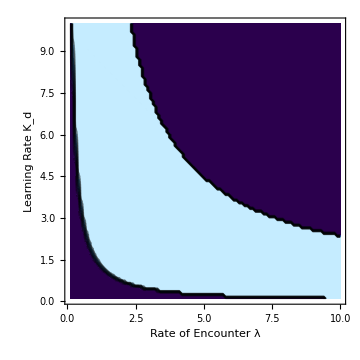

```mathematica
data=Flatten[<<"datakdλcF1",1];
kdλcF1=ListContourPlot[data,Contours->Table[c,{c,0.1,0.9,0.1}],Frame->{{True,True},{True,True}},FrameStyle->Directive[Thick,Black,14],ImageSize->Medium,FrameLabel->{Text[Style["Rate of Encounter λ",Black,20]],Text[Style["Learning Rate K_d",Black,20]]},ColorFunction->("DeepSeaColors")]
```

#### Δ = .05; Row 1

```mathematica
data=Flatten[<<"datakdλcF2",1];
kdλcF2=ListContourPlot[data,Contours->Table[c,{c,0.1,0.9,0.1}],Frame->{{True,True},{True,True}},FrameStyle->Directive[Thick,Black,14],ImageSize->Medium,FrameLabel->{Text[Style["Rate of Encounter λ",Black,20]],Text[Style["Learning Rate K_d",Black,20]]},ColorFunction->("DeepSeaColors")]
```

-Graphics-

#### Δ = .02; Row 1

```mathematica
data=Flatten[<<"datakdλcF3",1];
kdλcF3=ListContourPlot[data,Contours->Table[c,{c,0.1,0.9,0.1}],Frame->{{True,True},{True,True}},FrameStyle->Directive[Thick,Black,14],ImageSize->Medium,FrameLabel->{Text[Style["Rate of Encounter λ",Black,20]],Text[Style["Learning Rate K_d",Black,20]]},ColorFunction->("DeepSeaColors")]
```

-Graphics-

### Row 2

#### Δ = .02; Row 2

```mathematica
data=Flatten[<<"datakfλcF1",1];
kfλcF1=ListContourPlot[data,Contours->Table[c,{c,0.1,0.9,0.1}],Frame->{{True,True},{True,True}},FrameStyle->Directive[Thick,Black,14],ImageSize->Medium,FrameLabel->{Text[Style["Rate of Encounter λ",Black,20]],Text[Style["Half Saturation of Fear K_f",Black,20]]},ColorFunction->("DeepSeaColors")]
```

-Graphics-

#### Δ = .05; Row 2

```mathematica
data=Flatten[<<"datakfλcF2",1];
kfλcF2=ListContourPlot[data,Contours->Table[c,{c,0.1,0.9,0.1}],Frame->{{True,True},{True,True}},FrameStyle->Directive[Thick,Black,14],ImageSize->Medium,FrameLabel->{Text[Style["Rate of Encounter λ",Black,20]],Text[Style["Half Saturation of Fear K_f",Black,20]]},ColorFunction->("DeepSeaColors")]
```

-Graphics-

#### Δ = .08; Row 2

```mathematica
data=Flatten[<<"datakfλcF3",1];
kfλcF3=ListContourPlot[data,Contours->Table[c,{c,0.1,0.9,0.1}],Frame->{{True,True},{True,True}},FrameStyle->Directive[Thick,Black,14],ImageSize->Medium,FrameLabel->{Text[Style["Rate of Encounter λ",Black,20]],Text[Style["Half Saturation of Fear K_f",Black,20]]},ColorFunction->("DeepSeaColors")]
```

-Graphics-

### Grid

```mathematica
cFgrid=Grid[{{Text[Style["   Δ 0.02",20,TextAlignment->Center]],Text[Style["    Δ 0.05",20,TextAlignment->Center]],Text[Style["     Δ 0.08",20,TextAlignment->Center]]},{kdλcF3,kdλcF2,kdλcF1},{kfλcF3,kfλcF2,kfλcF1}}]
```

Δ 0.02 |     Δ 0.05 |      Δ 0.08
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-